# 1. Coxeter Groups

## 1.1 Basics

## 1.1.1 Coxeter group matrices

```mathematica
symmEntry[i_,j_]:=If[i==j,1,If[Abs[i-j]==1,3,2]]
```

### Finite groups

```mathematica
typeA[n_]:=
typeA[n]=Table[symmEntry[i,j],{i,1,n},{j,1,n}]
typeB[n_]:=
typeB[n]=Table[If[Or[i==n&&j==n-1,i==n-1&&j==n],4,symmEntry[i,j]],{i,1,n},{j,1,n}]
typeC[n_]:=
typeC[n]=typeB[n]
typeD[n_]:=
typeD[n]=Table[If[Or[i==n&&j==n-2,i==n-2&&j==n],3,If[Or[i==n&&j==n-1,i==n-1&&j==n],2,symmEntry[i,j]]],{i,1,n},{j,1,n}]
E6={{1,3,2,2,2,2},{3,1,3,2,2,2},{2,3,1,3,2,3},{2,2,3,1,3,2},{2,2,2,3,1,2},{2,2,3,2,2,1}};
E7={{1,3,2,2,2,2,2},{3,1,3,2,2,2,2},{2,3,1,3,2,2,3},{2,2,3,1,3,2,2},{2,2,2,3,1,3,2},{2,2,2,2,3,1,2},{2,2,3,2,2,2,1}};
E8={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,3},{2,2,3,1,3,2,2,2},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,1}};
F4={{1,3,2,2},{3,1,4,2},{2,4,1,3},{2,2,3,1}};
G2={{1,6},{6,1}};
H3={{1,3,2},{3,1,5},{2,5,1}};
H4={{1,3,2,2},{3,1,3,2},{2,3,1,5},{2,2,5,1}};
I2[m_]:={{1,m},{m,1}};
```

### Euclidean groups

```mathematica
ST={{1,4,4},{4,1,2},{4,2,1}};(*symmetry group of square tiling*)
S={{1,Infinity,2,2},{Infinity,1,2,2},{2,2,1,Infinity},{2,2,Infinity,1}};(*D_\infty^2*)
HT={{1,6,3},{6,1,2},{3,2,1}};(*Hexagonal tiling*)
TT={{1,3,3},{3,1,3},{3,3,1}};(*Tiling by equilateral Triangles*)
typeAE[1]={{1,Infinity},{Infinity,1}};
typeAE[n_]:=typeA[n+1]+Table[Table[If[Or[And[i==1,j==n+1],And[i==n+1,j==1]],1,0],{i,1,n+1}],{j,1,n+1}]/;n>1
typeBE[2]={{1,4,2},{4,1,4},{2,4,1}};
typeBE[n_]:=Table[If[And[i<n+1,j<n+1],typeB[n][[i]][[j]],If[And[i==n+1,j==n+1],1,If[Or[i==2,j==2],3,2]]],{i,1,n+1},{j,1,n+1}]/;n>2
typeCE[n_]:=typeB[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],1,0],{i,1,n+1},{j,1,n+1}]/;n>2
typeDE[n_]:=typeD[n+1]+Table[If[Or[And[i==1,j==2],And[i==2,j==1]],-1,If[Or[And[i==1,j==3],And[i==3,j==1]],1,0]],{i,1,n+1},{j,1,n+1}]/;n>3
EE6=Table[If[And[i<7,j<7],E6[[i]][[j]],If[Or[And[i==7,j==7]],1,If[Or[i==6,j==6],3,2]]],{i,1,7},{j,1,7}];
EE7={{1,3,2,2,2,2,2,2},{3,1,3,2,2,2,2,2},{2,3,1,3,2,2,2,2},{2,2,3,1,3,2,2,3},{2,2,2,3,1,3,2,2},{2,2,2,2,3,1,3,2},{2,2,2,2,2,3,1,2},{2,2,2,3,2,2,2,1}};
EE8={{1,3,2,2,2,2,2,2,2},{3,1,3,2,2,2,2,2,2},{2,3,1,3,2,2,2,2,3},{2,2,3,1,3,2,2,2,2},{2,2,2,3,1,3,2,2,2},{2,2,2,2,3,1,3,2,2},{2,2,2,2,2,3,1,3,2},{2,2,2,2,2,2,3,1,2},{2,2,3,2,2,2,2,2,1}};
FE4={{1,3,2,2,2},{3,1,3,2,2},{2,3,1,4,2},{2,2,4,1,3},{2,2,2,3,1}};
GE2={{1,3,2},{3,1,6},{2,6,1}};
```

### Hyperbolic groups

```mathematica
triangle[p_,q_,r_]:={{1,p,r},{p,1,q},{r,q,1}};
```

### Right - angled Coxeter groups

```mathematica
raHexagon={{1,2,Infinity,Infinity,Infinity,2},{2,1,2,Infinity,Infinity,Infinity},{Infinity,2,1,2,Infinity,Infinity},{Infinity,Infinity,2,1,2,Infinity},{Infinity,Infinity,Infinity,2,1,2},{2,Infinity,Infinity,Infinity,2,1}};
raPentagon={{1,2,Infinity,Infinity,2},{2,1,2,Infinity,Infinity},{Infinity,2,1,2,Infinity},{Infinity,Infinity,2,1,2},{2,Infinity,Infinity,2,1}};
raSquare={{1,2,Infinity,2},{2,1,2,Infinity},{Infinity,2,1,2},{2,Infinity,2,1}};
raTriangle={{1,2,2},{2,1,2},{2,2,1}};
bipart[3,3]={{1,2,Infinity,2,Infinity,2},{2,1,2,Infinity,2,Infinity},{Infinity,2,1,2,Infinity,2},{2,Infinity,2,1,2,Infinity},{Infinity,2,Infinity,2,1,2},{2,Infinity,2,Infinity,2,1}};
bipart[3,2]={{1,2,Infinity,2,Infinity},{2,1,2,Infinity,2},{Infinity,2,1,2,Infinity},{2,Infinity,2,1,2},{Infinity,2,Infinity,2,1}};
```

## 1.1.2 Group properties

### Group Size

```mathematica
size[E6]=51840;
size[E7]=2903040;
size[E8]=696729600;
size[F4]=1152;
size[G2]=12;
size[H3]=120;
size[H4]=14400;
size[M_]:=Module[{n},
n=rank[M];
If[n==2,2M[[1]][[2]],
If[M==typeA[n],Factorial[n+1],
If[M==typeB[n],2^n Factorial[n],
If[M==typeD[n],2^(n-1)Factorial[n],Infinity]]]]]
```

### Maximum Length

```mathematica
maxLength[E6]=36;
maxLength[E7]=63;
maxLength[E8]=120;
maxLength[F4]=24;
maxLength[G2]=6;
maxLength[H3]=15;
maxLength[H4]=60;
maxLength[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],Binomial[n+1,2],
If[M==typeB[n],n^2,
If[M==typeD[n],n^2-n,Infinity]]]]]
```

### Coxeter Number

```mathematica
coxeterNumber[E6]=12;
coxeterNumber[E7]=18;
coxeterNumber[E8]=30;
coxeterNumber[F4]=12;
coxeterNumber[G2]=6;
coxeterNumber[H3]=10;
coxeterNumber[H4]=30;
coxeterNumber[M_]:=Module[{n},
n=rank[M];
If[n==2,M[[1]][[2]],
If[M==typeA[n],n+1,
If[M==typeB[n],2n,
If[M==typeD[n],2n-1,Infinity]]]]]
```

### Group Automorphisms

```mathematica
inverse[w_String]:=StringReverse[w]
involutionQ[M_,w_String]:=linWordProblem[M,w,inverse[w]]
elementAutomorphisms[M_,w_String]:=deleteRepeatedElements[M,Join[{w,inverse[w]},StringReplace[w,#]&/@diagramAutomorphisms[M]]]
automorphismOrbitQ[M_,w_String,u_String]:=Fold[Or,linWordProblem[M,#,u]&/@elementAutomorphisms[M,w]]
automorphismRepresentatives[M_,{}]:={}
automorphismRepresentatives[M_,wList_List]:=Join[{wList[[1]]},automorphismRepresentatives[M,Select[wList,Not[automorphismOrbitQ[M,wList[[1]],#]]&]]]
```

#### Group Data

```mathematica
diagramAutomorphisms[M_]:={{},Table[ToString[i]-> ToString[rank[M]+1-i],{i,1,rank[M]}]}/;MemberQ[typeA[rank[M]],typeCE[rank[M]-1]]
diagramAutomorphisms[M_]:={{}}/;And[MemberQ[Select[{typeB[rank[M]],E7,E8,H3,H4,EE8,FE4,GE2,HT},rank[#]==rank[M]&],M],Not[rank[M]==2]]
diagramAutomorphisms[M_]:={{},{"1"->"2","2"->"1"}}/;rank[M]==2
diagramAutomorphisms[typeD[4]]={{"1"->"4","4"->"1"},{"1"->"3","3"->"1"},{"3"->"4","4"->"3"},{"1"->"4","4"->"3","3"->"1"},{"1"->"3","3"->"4","4"->"1"}};
diagramAutomorphisms[M_]:={{},{ToString[rank[M]]-> ToString[rank[M]-1],ToString[rank[M]-1]-> ToString[rank[M]]}}/;And[M==typeD[rank[M]],rank[M]>4]
diagramAutomorphisms[E6]={{},{"1"->"5","2"->"4","4"->"2","5"->"1"}};
diagramAutomorphisms[F4]={{},{"1"-> "4","2"->"3","3"-> "2","4"->"1"}};
diagramAutomorphisms[ST]={{},{"2"->"3","3"-> "2"}};
diagramAutomorphisms[S]={{},{"1"->"2","2"->"1"},{"3"->"4","4"->"3"},{"1"->"2","2"->"1","3"->"4","4"->"3"}};
diagramAutomorphisms[TT]={{},{"1"->"2","2"->"1"},{"1"->"3","3"->"1"},{"3"->"2","2"->"3"},{"1"->"2","2"->"3","3"->"1"},{"1"->"3","3"->"2","2"->"1"}};
diagramAutomorphisms[M_]:=Join[Join[{{}},Table[Table[ToString[i]-> ToString[Mod[i+j,rank[M],1]],{i,1,rank[M]}],{j,1,rank[M]-1}]],Table[Table[ToString[i]-> ToString[Mod[2j+1-i,rank[M],1]],{i,1,rank[M]}],{j,1,rank[M]}]]/;And[M==typeAE[rank[M]-1],Not[rank[M]==2]]
diagramAutomorphisms[typeBE[2]]={{},{"1"->"3","3"->"1"}};
diagramAutomorphisms[M_]:={{},{"1"-> ToString[rank[M]],ToString[rank[M]]->"1"}}/;And[M==typeBE[rank[M]-1],Not[rank[M]==3]]
diagramAutomorphisms[M_]:={{},{"1"->"2","2"->"1"},{ToString[rank[M]]-> ToString[rank[M]-1],ToString[rank[M]-1]-> ToString[rank[M]]},{"1"->"2","2"->"1",ToString[rank[M]]-> ToString[rank[M]-1],ToString[rank[M]-1]-> ToString[rank[M]]},Table[ToString[i]-> ToString[rank[M]+1-i],{i,1,rank[M]}],Join[Table[ToString[i]-> ToString[rank[M]+1-i],{i,3,rank[M]-2}],{"1"->ToString[rank[M]-1],"2"->ToString[rank[M]],ToString[rank[M]]-> "1",ToString[rank[M]-1]-> "2"}],Join[Table[ToString[i]-> ToString[rank[M]+1-i],{i,3,rank[M]-2}],{"1"->ToString[rank[M]],"2"->ToString[rank[M]-1],ToString[rank[M]]-> "2",ToString[rank[M]-1]-> "1"}],Join[Table[ToString[i]-> ToString[rank[M]+1-i],{i,3,rank[M]-2}],{"1"->ToString[rank[M]-1],"2"->ToString[rank[M]],ToString[rank[M]]-> "2",ToString[rank[M]-1]-> "1"}]}/;M==typeDE[rank[M]-1]
diagramAutomorphisms[EE6]={{},{"1"->"5","2"->"4","4"->"2","5"->"1"},{"1"->"7","2"->"6","6"->"2","7"->"1"},{"7"->"5","6"->"4","4"->"6","5"->"7"},{"1"-> "7","7"-> "5","5"-> "1","2"-> "6","6"-> "4","4"-> "2"},{"1"-> "5","5"-> "7","7"-> "1","2"-> "4","4"-> "6","6"-> "2"}};
diagramAutomorphisms[EE7]={{},{"1"->"7","2"->"6","3"->"5","5"->"3","6"->"2","7"->"1"}};
```

## 1.1.3 Basic functions

```mathematica
rank[M_]:=Tr[M](*calculates number of generators*)
form[M_]:=Table[Table[-Cos[Pi/M[[i]][[j]]],{j,rank[M]}],{i,rank[M]}] (*gives the canonical bilinear form associated to Coxeter matrix M*)
listToString[w_List]:=StringJoin[Table[ToString[w[[i]]],{i,Length[w]}]] (*converts a word in the form of a list to a string*)
stringToList[w_String]:=Table[StringTake[w,{i}],{i,StringLength[w]}] (*converts a word in the form of a string to a list*)
makeString[w_]:=listToString[w]/;Head[w]==List (*makes word w a string*)
makeString[w_]:=w/;Head[w]==String 
makeList[w_]:=w/;Head[w]==List (*makes word w a list*)
makeList[w_]:=stringToList[w]/;Head[w]==String 
signature[A_]:={Length[Select[Eigenvalues[A],#>0&]],Length[Select[Eigenvalues[A],#==0&]],Length[Select[Eigenvalues[A],#<0&]]}
euclideanQ[M_]:=signature[form[M]]=={rank[M]-1,1,0}
sphericalQ[M_]:=signature[form[M]]=={rank[M],0,0}
hyperbolicQ[M_]:=signature[form[M]]=={rank[M]-1,0,1}
evenQ[M_]:=Fold[And,Or[EvenQ[#],#==Infinity]&/@Complement[DeleteDuplicates[Flatten[M]],{1}]]
```

## 1.1.4 Inversions

```mathematica
makePalindromic[s_String]:=StringJoin[s,StringDrop[StringReverse[s],1]]
inv[M_,w_String]:=Table[Select[reduce[M,makePalindromic[StringTake[findReduced[M,w],k]]],PalindromeQ[#]&,1][[1]],{k,1,coxeterLength[M,w]}]
centralGenerator[w_String]:=StringTake[w,{(StringLength[w]+1)/2}]/;PalindromeQ[w]
conjugatingElement[w_String]:=StringTake[w,(StringLength[w]-1)/2]/;PalindromeQ[w]
```

## 1.1.5 Some more useful basic functions

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
gpMultiply[v_,w_]:=makeString[Join[makeList[v],makeList[w]]]
longestElement[M_]:=Fold[gpMultiply,Table[coxeterElement[M],{i,1,coxeterNumber[M]/2}]]/;EvenQ[coxeterNumber[M]]
longestElement[M_]:=braid[{M[[1]][[2]],1,2}]/;rank[M]==2
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
deleteRepeatedElements[M_,wList_List]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
matWord={mat[M,#],#}&/@wList;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,MemberQ[wList,#]&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
(*deleteRepeatedElements[M,wList]=*)Complement[list2,extraWords]
]
```

## 1.1.6 Generating sets

```mathematica
resolvedQ[M_,wList_]:=Length[DeleteDuplicates[Table[StringTake[StringJoin[wList],{i}],{i,1,StringLength[StringJoin[wList]]}]]]==rank[M]
fullGroupCompletionQ[M_,squareComplex_]:=cubeCount[squareComplex]==<|"vertexCount"->1,"edgeCount"->rank[M],"squareCount"->Length[Select[Flatten[M],#==2&]]/2|>(*simple test as to whether squareComplex is likely to be a completion for M, good test so long as we assume squareComplex is a completion for some subgroup of M*)
generatingSetQ[M_,wList_]:=If[resolvedQ[M,wList],fullGroupCompletionQ[M,completion[M,wList]],False]
randomSubset[set_,{size_}]:=Block[{setSize,randomPerm},
setSize=Length[set];
randomPerm=RandomPermutation[setSize];
Take[Permute[set,randomPerm],size]
]
randomSubsets[set_,{size_},number_]:=Join[{randomSubset[set,{size}]},randomSubsets[set,{size},number-1]]/;number>1
randomSubsets[set_,{size_},1]:={randomSubset[set,{size}]}
findGeneratingSets[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=randomSubset[elementList,{size}];
If[
generatingSetQ[M,candidate],
If[
number>1,
Print[candidate];
findGeneratingSets[M,elementList,size,number-1],
candidate
],
findGeneratingSets[M,elementList,size,number]
]
]
(*findGeneratingSet[M_,elementList_,seed_:{}]:=Block[{randomElement,candidate},
randomElement=Take[elementList,{RandomInteger[{1,Length[elementList]}]}][[1]];
candidate=Append[seed,randomElement];
If[
generatingSetQ[M,candidate],
candidate,
findGeneratingSet[M,elementList,candidate]
]
]*)
generatingSetObviouslyStandardQ[M_,wList_]:=cubeCount[nonClosingCompletion[M,setToRose[wList]]][["vertexCount"]]==1
findNonObviouslyStandardGeneratingSet[M_,elementList_,size_,number_:1]:=Block[{candidate},
candidate=findGeneratingSets[M,elementList,size];
If[
Not[generatingSetObviouslyStandardQ[M,candidate]],
If[
number>1,
Print[candidate];
findNonObviouslyStandardGeneratingSet[M,elementList,size,number-1],
candidate
],
findNonObviouslyStandardGeneratingSet[M,elementList,size,number]
]
]
```

## 1.2 Element enumeration

## 1.2.1 Tit’s solution to the word problem

Relations

```mathematica
rel[M_]:=Module[{all,depth},
all=Table[{M[[i]][[j]],i,j},{i,1,rank[M]},{j,1,rank[M]}];
depth=If[MemberQ[Flatten[all],Infinity],4,3];
rel[M]=Select[Flatten[all,Depth[all]-depth],Not[#[[1]]==Infinity]&&Not[#[[1]]==1]&]
](*the non-trivial relations on M in the form {m_{ij},i,j}*)
braid[{n_,i_,j_}]:=makeString[Take[Flatten[Table[{i,j},{k,n}]],n] ](*the LHS of the relation for ij*)
inverseBraid[{n_,i_,j_}]:=braid[{n,j,i}] (*the RHS for the relation for ij*)
inverseBraid[b_String]:=inverseBraid[{StringLength[b],StringTake[b,{1}],StringTake[b,{2}]}]
relations[M_]:=braid[#]&/@rel[M](*lists the R/LHS of all braid relations in the group*)
```

Type 1 M-move

```mathematica
oneMoveM1[M_,w_]:=StringReplace[makeString[w],x_~~x_->""] 
moveM1[M_,w_]:=Module[{v,n,x,m},
v=makeString[w];
n=StringLength[v];
x=oneMoveM1[M,v];
m=StringLength[x];
If[m==n,x,moveM1[M,x]]
](*performs all Tits moves of type 1 on w which are possible*)
```

Type 2 M-move

```mathematica
locate[w_String,b_String]:={b,#}&/@StringPosition[w,b](*produces an indexed list of the positions of all occurences of the substring b in w*)
locateAll[w_String,b_List]:=Fold[Join,locate[w,#]&/@b](*produces an indexed list of the positions of all occurences of the substrings of b in w*)
oneMoveM2[M_,w_String]:=
DeleteDuplicates[Join[{w},Flatten[StringReplaceList[makeString[w],#->inverseBraid[#]]&/@relations[M]]]](*produces a list of all words accessinle form w by a single M2 move, together with w itself*)
oneMoveM2[M_,wList_List]:=DeleteDuplicates[Join[wList,Fold[Join,oneMoveM2[M,#]&/@wList]]]
```

Reduction

```mathematica
reducibleQ[w_]:=StringContainsQ[makeString[w],x_~~x_](*returns True if w contains a repeated letter*)
reducibleQ[wList_List]:=Fold[Or,reducibleQ[#]&/@wList]
findReducible[M_,wList_List]:=Select[wList,reducibleQ[#]&,1][[1]](*gives an element of wList which contains a double letter*)
reduce[M_,w_List]:=
reduce[M,w]=reduce[M,makeString[w]]/;Length[w]>1&&Length[w[[1]]]==1(*returs the list of all reduced words for w*)
reduce[M_,w_String]:=
reduce[M,w]=If[reducibleQ[w],reduce[M,moveM1[M,makeString[w]]],reduce[M,oneMoveM2[M,w]]]
reduce[M_,wList_List]:=reduce[M,moveM1[M,findReducible[M,wList]]]/;reducibleQ[wList]
reduce[M_,wList_List]:=Module[{wList2},
wList2=oneMoveM2[M,wList];
If[wList==wList2,wList,reduce[M,oneMoveM2[M,wList]]]
]/;Not[reducibleQ[wList]]&& Not[Length[w]>1&&Length[w[[1]]]==1]
findReduced[M_,w_]:=
findReduced[M,w]=Sort[reduce[M,w]][[1]](*returns a reduced word for w*)
coxeterLength[M_,w_]:=
coxeterLength[M,w]=StringLength[findReduced[M,w]](*calculates the length of the element w*)
```

Comparing

```mathematica
titsWordProblem[M_,w_,v_]:=MemberQ[reduce[M,w],findReduced[M,v]](*returns True id w and v express the same element in M*)
```

## 1.2.2 Linear solution to the word problem

```mathematica
e[M_,i_]:=UnitVector[rank[M],i] (*gives the ith standard unit vector*)
mat[M_,w_String]:=
mat[M,w]=If[StringLength[w]==0,
IdentityMatrix[rank[M]],
If[StringLength[w]==1,
Module[{i},
i=ToExpression[w];
ArrayFlatten[{Table[Transpose[{e[M,j]-2form[M][[i]][[j]]e[M,i]}],{j,rank[M]}]}] 
],
Simplify[Dot[mat[M,StringTake[w,-1]],mat[M,StringDrop[w,-1]]]]
]
]
mat[M_,w_List]:=mat[M,makeString[w]]
linWordProblem[M_,u_,v_]:=mat[M,u]==mat[M,v]
```

## 1.2.3 Group elements

```mathematica
enumeratedGroups={
{typeA[3],6},
{typeA[5],15},
{typeA[6],21},
{typeB[5],25},
{typeD[6],30},
{E6,36},
{E7,10},
{E8,9},
{F4,24},
{H3,15},
{H4,60},
{ST,66},
{S,66},
{HT,66},
{TT,66},
{typeAE[1],300},
{typeAE[2],66},
{typeAE[3],25},
{typeAE[4],17},
{typeBE[3],25},
{typeBE[4],15},
{typeBE[5],14},
{typeCE[3],25},
{typeCE[4],15},
{typeCE[5],15},
{typeDE[4],15},
{typeDE[5],11},
{EE6,10},
{EE7,10},
{EE8,9},
{FE4,25},
{GE2,66},
{raPentagon,9},
{raHexagon,7},
{bipart[3,2],8},
{bipart[3,3],8}
};
enumeratedQ[M_,k_]:=If[MemberQ[#[[1]]&/@enumeratedGroups,M],Select[enumeratedGroups,#[[1]]==M&][[1]][[2]]≥ k,False]
enumeratedQ[M_]:=enumeratedQ[M,maxLength[M]]
lengthEnumerated[M_]:=If[MemberQ[#[[1]]&/@enumeratedGroups,M],Select[enumeratedGroups,#[[1]]==M&][[1]][[2]],0]
```

#### Finite Groups

Type A[3]

```mathematica
words[typeA[3],6]={"","1","12","121","1213","12132","121321","123","1232","12321","13","132","1321","2","21","213","2132","21321","23","232","2321","3","32","321"};
```

Type A[5]

```mathematica
words[typeA[5],15]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321435","1213214354","12132143543","121321435432","1213214354321","12132145","121321454","1213214543","12132145432","121321454321","1213215","12132154","121321543","1213215432","12132154321","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324325","1213243254","12132432543","121324325432","1213243254321","12132435","121324354","1213243543","12132435432","121324354321","1213245","12132454","121324543","1213245432","12132454321","121325","1213254","12132543","121325432","1213254321","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134325","121343254","1213432543","12134325432","121343254321","1213435","12134354","121343543","1213435432","12134354321","121345","1213454","12134543","121345432","1213454321","12135","121354","1213543","12135432","121354321","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214325","12143254","121432543","1214325432","12143254321","121435","1214354","12143543","121435432","1214354321","12145","121454","1214543","12145432","121454321","1215","12154","121543","1215432","12154321","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214325","1232143254","12321432543","123214325432","1232143254321","12321435","123214354","1232143543","12321435432","123214354321","1232145","12321454","123214543","1232145432","12321454321","123215","1232154","12321543","123215432","1232154321","12324","123243","1232432","12324321","123243215","1232432154","12324321543","123243215432","1232432154321","12324325","123243254","1232432543","12324325432","123243254321","1232435","12324354","123243543","1232435432","12324354321","123245","1232454","12324543","123245432","1232454321","12325","123254","1232543","12325432","123254321","1234","12343","123432","1234321","12343215","123432154","1234321543","12343215432","123432154321","1234325","12343254","123432543","1234325432","12343254321","123435","1234354","12343543","123435432","1234354321","12345","123454","1234543","12345432","123454321","1235","12354","123543","1235432","12354321","124","1243","12432","124321","1243215","12432154","124321543","1243215432","12432154321","124325","1243254","12432543","124325432","1243254321","12435","124354","1243543","12435432","124354321","1245","12454","124543","1245432","12454321","125","1254","12543","125432","1254321","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","13214321543","132143215432","1321432154321","13214325","132143254","1321432543","13214325432","132143254321","1321435","13214354","132143543","1321435432","13214354321","132145","1321454","13214543","132145432","1321454321","13215","132154","1321543","13215432","132154321","1324","13243","132432","1324321","13243215","132432154","1324321543","13243215432","132432154321","1324325","13243254","132432543","1324325432","13243254321","132435","1324354","13243543","132435432","1324354321","13245","132454","1324543","13245432","132454321","1325","13254","132543","1325432","13254321","134","1343","13432","134321","1343215","13432154","134321543","1343215432","13432154321","134325","1343254","13432543","134325432","1343254321","13435","134354","1343543","13435432","134354321","1345","13454","134543","1345432","13454321","135","1354","13543","135432","1354321","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","14325","143254","1432543","14325432","143254321","1435","14354","143543","1435432","14354321","145","1454","14543","145432","1454321","15","154","1543","15432","154321","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","21321432154","213214321543","2132143215432","21321432154321","213214325","2132143254","21321432543","213214325432","2132143254321","21321435","213214354","2132143543","21321435432","213214354321","2132145","21321454","213214543","2132145432","21321454321","213215","2132154","21321543","213215432","2132154321","21324","213243","2132432","21324321","213243215","2132432154","21324321543","213243215432","2132432154321","21324325","213243254","2132432543","21324325432","213243254321","2132435","21324354","213243543","2132435432","21324354321","213245","2132454","21324543","213245432","2132454321","21325","213254","2132543","21325432","213254321","2134","21343","213432","2134321","21343215","213432154","2134321543","21343215432","213432154321","2134325","21343254","213432543","2134325432","21343254321","213435","2134354","21343543","213435432","2134354321","21345","213454","2134543","21345432","213454321","2135","21354","213543","2135432","21354321","214","2143","21432","214321","2143215","21432154","214321543","2143215432","21432154321","214325","2143254","21432543","214325432","2143254321","21435","214354","2143543","21435432","214354321","2145","21454","214543","2145432","21454321","215","2154","21543","215432","2154321","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","23214321543","232143215432","2321432154321","23214325","232143254","2321432543","23214325432","232143254321","2321435","23214354","232143543","2321435432","23214354321","232145","2321454","23214543","232145432","2321454321","23215","232154","2321543","23215432","232154321","2324","23243","232432","2324321","23243215","232432154","2324321543","23243215432","232432154321","2324325","23243254","232432543","2324325432","23243254321","232435","2324354","23243543","232435432","2324354321","23245","232454","2324543","23245432","232454321","2325","23254","232543","2325432","23254321","234","2343","23432","234321","2343215","23432154","234321543","2343215432","23432154321","234325","2343254","23432543","234325432","2343254321","23435","234354","2343543","23435432","234354321","2345","23454","234543","2345432","23454321","235","2354","23543","235432","2354321","24","243","2432","24321","243215","2432154","24321543","243215432","2432154321","24325","243254","2432543","24325432","243254321","2435","24354","243543","2435432","24354321","245","2454","24543","245432","2454321","25","254","2543","25432","254321","3","32","321","3214","32143","321432","3214321","32143215","321432154","3214321543","32143215432","321432154321","3214325","32143254","321432543","3214325432","32143254321","321435","3214354","32143543","321435432","3214354321","32145","321454","3214543","32145432","321454321","3215","32154","321543","3215432","32154321","324","3243","32432","324321","3243215","32432154","324321543","3243215432","32432154321","324325","3243254","32432543","324325432","3243254321","32435","324354","3243543","32435432","324354321","3245","32454","324543","3245432","32454321","325","3254","32543","325432","3254321","34","343","3432","34321","343215","3432154","34321543","343215432","3432154321","34325","343254","3432543","34325432","343254321","3435","34354","343543","3435432","34354321","345","3454","34543","345432","3454321","35","354","3543","35432","354321","4","43","432","4321","43215","432154","4321543","43215432","432154321","4325","43254","432543","4325432","43254321","435","4354","43543","435432","4354321","45","454","4543","45432","454321","5","54","543","5432","54321"};
```

Type A[6]

```mathematica
words[typeA[6],21]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214321543216","12132143215432165","121321432154321654","1213214321543216543","12132143215432165432","121321432154321654321","121321432154326","1213214321543265","12132143215432654","121321432154326543","1213214321543265432","12132143215432654321","12132143215436","121321432154365","1213214321543654","12132143215436543","121321432154365432","1213214321543654321","1213214321546","12132143215465","121321432154654","1213214321546543","12132143215465432","121321432154654321","121321432156","1213214321565","12132143215654","121321432156543","1213214321565432","12132143215654321","12132143216","121321432165","1213214321654","12132143216543","121321432165432","1213214321654321","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543216","1213214325432165","12132143254321654","121321432543216543","1213214325432165432","12132143254321654321","12132143254326","121321432543265","1213214325432654","12132143254326543","121321432543265432","1213214325432654321","1213214325436","12132143254365","121321432543654","1213214325436543","12132143254365432","121321432543654321","121321432546","1213214325465","12132143254654","121321432546543","1213214325465432","12132143254654321","12132143256","121321432565","1213214325654","12132143256543","121321432565432","1213214325654321","1213214326","12132143265","121321432654","1213214326543","12132143265432","121321432654321","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543216","121321435432165","1213214354321654","12132143543216543","121321435432165432","1213214354321654321","1213214354326","12132143543265","121321435432654","1213214354326543","12132143543265432","121321435432654321","121321435436","1213214354365","12132143543654","121321435436543","1213214354365432","12132143543654321","12132143546","121321435465","1213214354654","12132143546543","121321435465432","1213214354654321","1213214356","12132143565","121321435654","1213214356543","12132143565432","121321435654321","121321436","1213214365","12132143654","121321436543","1213214365432","12132143654321","12132145","121321454","1213214543","12132145432","121321454321","1213214543216","12132145432165","121321454321654","1213214543216543","12132145432165432","121321454321654321","121321454326","1213214543265","12132145432654","121321454326543","1213214543265432","12132145432654321","12132145436","121321454365","1213214543654","12132145436543","121321454365432","1213214543654321","1213214546","12132145465","121321454654","1213214546543","12132145465432","121321454654321","121321456","1213214565","12132145654","121321456543","1213214565432","12132145654321","12132146","121321465","1213214654","12132146543","121321465432","1213214654321","1213215","12132154","121321543","1213215432","12132154321","121321543216","1213215432165","12132154321654","121321543216543","1213215432165432","12132154321654321","12132154326","121321543265","1213215432654","12132154326543","121321543265432","1213215432654321","1213215436","12132154365","121321543654","1213215436543","12132154365432","121321543654321","121321546","1213215465","12132154654","121321546543","1213215465432","12132154654321","12132156","121321565","1213215654","12132156543","121321565432","1213215654321","1213216","12132165","121321654","1213216543","12132165432","121321654321","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543216","1213243215432165","12132432154321654","121324321543216543","1213243215432165432","12132432154321654321","12132432154326","121324321543265","1213243215432654","12132432154326543","121324321543265432","1213243215432654321","1213243215436","12132432154365","121324321543654","1213243215436543","12132432154365432","121324321543654321","121324321546","1213243215465","12132432154654","121324321546543","1213243215465432","12132432154654321","12132432156","121324321565","1213243215654","12132432156543","121324321565432","1213243215654321","1213243216","12132432165","121324321654","1213243216543","12132432165432","121324321654321","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543216","121324325432165","1213243254321654","12132432543216543","121324325432165432","1213243254321654321","1213243254326","12132432543265","121324325432654","1213243254326543","12132432543265432","121324325432654321","121324325436","1213243254365","12132432543654","121324325436543","1213243254365432","12132432543654321","12132432546","121324325465","1213243254654","12132432546543","121324325465432","1213243254654321","1213243256","12132432565","121324325654","1213243256543","12132432565432","121324325654321","121324326","1213243265","12132432654","121324326543","1213243265432","12132432654321","12132435","121324354","1213243543","12132435432","121324354321","1213243543216","12132435432165","121324354321654","1213243543216543","12132435432165432","121324354321654321","121324354326","1213243543265","12132435432654","121324354326543","1213243543265432","12132435432654321","12132435436","121324354365","1213243543654","12132435436543","121324354365432","1213243543654321","1213243546","12132435465","121324354654","1213243546543","12132435465432","121324354654321","121324356","1213243565","12132435654","121324356543","1213243565432","12132435654321","12132436","121324365","1213243654","12132436543","121324365432","1213243654321","1213245","12132454","121324543","1213245432","12132454321","121324543216","1213245432165","12132454321654","121324543216543","1213245432165432","12132454321654321","12132454326","121324543265","1213245432654","12132454326543","121324543265432","1213245432654321","1213245436","12132454365","121324543654","1213245436543","12132454365432","121324543654321","121324546","1213245465","12132454654","121324546543","1213245465432","12132454654321","12132456","121324565","1213245654","12132456543","121324565432","1213245654321","1213246","12132465","121324654","1213246543","12132465432","121324654321","121325","1213254","12132543","121325432","1213254321","12132543216","121325432165","1213254321654","12132543216543","121325432165432","1213254321654321","1213254326","12132543265","121325432654","1213254326543","12132543265432","121325432654321","121325436","1213254365","12132543654","121325436543","1213254365432","12132543654321","12132546","121325465","1213254654","12132546543","121325465432","1213254654321","1213256","12132565","121325654","1213256543","12132565432","121325654321","121326","1213265","12132654","121326543","1213265432","12132654321","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543216","121343215432165","1213432154321654","12134321543216543","121343215432165432","1213432154321654321","1213432154326","12134321543265","121343215432654","1213432154326543","12134321543265432","121343215432654321","121343215436","1213432154365","12134321543654","121343215436543","1213432154365432","12134321543654321","12134321546","121343215465","1213432154654","12134321546543","121343215465432","1213432154654321","1213432156","12134321565","121343215654","1213432156543","12134321565432","121343215654321","121343216","1213432165","12134321654","121343216543","1213432165432","12134321654321","12134325","121343254","1213432543","12134325432","121343254321","1213432543216","12134325432165","121343254321654","1213432543216543","12134325432165432","121343254321654321","121343254326","1213432543265","12134325432654","121343254326543","1213432543265432","12134325432654321","12134325436","121343254365","1213432543654","12134325436543","121343254365432","1213432543654321","1213432546","12134325465","121343254654","1213432546543","12134325465432","121343254654321","121343256","1213432565","12134325654","121343256543","1213432565432","12134325654321","12134326","121343265","1213432654","12134326543","121343265432","1213432654321","1213435","12134354","121343543","1213435432","12134354321","121343543216","1213435432165","12134354321654","121343543216543","1213435432165432","12134354321654321","12134354326","121343543265","1213435432654","12134354326543","121343543265432","1213435432654321","1213435436","12134354365","121343543654","1213435436543","12134354365432","121343543654321","121343546","1213435465","12134354654","121343546543","1213435465432","12134354654321","12134356","121343565","1213435654","12134356543","121343565432","1213435654321","1213436","12134365","121343654","1213436543","12134365432","121343654321","121345","1213454","12134543","121345432","1213454321","12134543216","121345432165","1213454321654","12134543216543","121345432165432","1213454321654321","1213454326","12134543265","121345432654","1213454326543","12134543265432","121345432654321","121345436","1213454365","12134543654","121345436543","1213454365432","12134543654321","12134546","121345465","1213454654","12134546543","121345465432","1213454654321","1213456","12134565","121345654","1213456543","12134565432","121345654321","121346","1213465","12134654","121346543","1213465432","12134654321","12135","121354","1213543","12135432","121354321","1213543216","12135432165","121354321654","1213543216543","12135432165432","121354321654321","121354326","1213543265","12135432654","121354326543","1213543265432","12135432654321","12135436","121354365","1213543654","12135436543","121354365432","1213543654321","1213546","12135465","121354654","1213546543","12135465432","121354654321","121356","1213565","12135654","121356543","1213565432","12135654321","12136","121365","1213654","12136543","121365432","1213654321","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214321543216","12143215432165","121432154321654","1214321543216543","12143215432165432","121432154321654321","121432154326","1214321543265","12143215432654","121432154326543","1214321543265432","12143215432654321","12143215436","121432154365","1214321543654","12143215436543","121432154365432","1214321543654321","1214321546","12143215465","121432154654","1214321546543","12143215465432","121432154654321","121432156","1214321565","12143215654","121432156543","1214321565432","12143215654321","12143216","121432165","1214321654","12143216543","121432165432","1214321654321","1214325","12143254","121432543","1214325432","12143254321","121432543216","1214325432165","12143254321654","121432543216543","1214325432165432","12143254321654321","12143254326","121432543265","1214325432654","12143254326543","121432543265432","1214325432654321","1214325436","12143254365","121432543654","1214325436543","12143254365432","121432543654321","121432546","1214325465","12143254654","121432546543","1214325465432","12143254654321","12143256","121432565","1214325654","12143256543","121432565432","1214325654321","1214326","12143265","121432654","1214326543","12143265432","121432654321","121435","1214354","12143543","121435432","1214354321","12143543216","121435432165","1214354321654","12143543216543","121435432165432","1214354321654321","1214354326","12143543265","121435432654","1214354326543","12143543265432","121435432654321","121435436","1214354365","12143543654","121435436543","1214354365432","12143543654321","12143546","121435465","1214354654","12143546543","121435465432","1214354654321","1214356","12143565","121435654","1214356543","12143565432","121435654321","121436","1214365","12143654","121436543","1214365432","12143654321","12145","121454","1214543","12145432","121454321","1214543216","12145432165","121454321654","1214543216543","12145432165432","121454321654321","121454326","1214543265","12145432654","121454326543","1214543265432","12145432654321","12145436","121454365","1214543654","12145436543","121454365432","1214543654321","1214546","12145465","121454654","1214546543","12145465432","121454654321","121456","1214565","12145654","121456543","1214565432","12145654321","12146","121465","1214654","12146543","121465432","1214654321","1215","12154","121543","1215432","12154321","121543216","1215432165","12154321654","121543216543","1215432165432","12154321654321","12154326","121543265","1215432654","12154326543","121543265432","1215432654321","1215436","12154365","121543654","1215436543","12154365432","121543654321","121546","1215465","12154654","121546543","1215465432","12154654321","12156","121565","1215654","12156543","121565432","1215654321","1216","12165","121654","1216543","12165432","121654321","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543216","1232143215432165","12321432154321654","123214321543216543","1232143215432165432","12321432154321654321","12321432154326","123214321543265","1232143215432654","12321432154326543","123214321543265432","1232143215432654321","1232143215436","12321432154365","123214321543654","1232143215436543","12321432154365432","123214321543654321","123214321546","1232143215465","12321432154654","123214321546543","1232143215465432","12321432154654321","12321432156","123214321565","1232143215654","12321432156543","123214321565432","1232143215654321","1232143216","12321432165","123214321654","1232143216543","12321432165432","123214321654321","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543216","123214325432165","1232143254321654","12321432543216543","123214325432165432","1232143254321654321","1232143254326","12321432543265","123214325432654","1232143254326543","12321432543265432","123214325432654321","123214325436","1232143254365","12321432543654","123214325436543","1232143254365432","12321432543654321","12321432546","123214325465","1232143254654","12321432546543","123214325465432","1232143254654321","1232143256","12321432565","123214325654","1232143256543","12321432565432","123214325654321","123214326","1232143265","12321432654","123214326543","1232143265432","12321432654321","12321435","123214354","1232143543","12321435432","123214354321","1232143543216","12321435432165","123214354321654","1232143543216543","12321435432165432","123214354321654321","123214354326","1232143543265","12321435432654","123214354326543","1232143543265432","12321435432654321","12321435436","123214354365","1232143543654","12321435436543","123214354365432","1232143543654321","1232143546","12321435465","123214354654","1232143546543","12321435465432","123214354654321","123214356","1232143565","12321435654","123214356543","1232143565432","12321435654321","12321436","123214365","1232143654","12321436543","123214365432","1232143654321","1232145","12321454","123214543","1232145432","12321454321","123214543216","1232145432165","12321454321654","123214543216543","1232145432165432","12321454321654321","12321454326","123214543265","1232145432654","12321454326543","123214543265432","1232145432654321","1232145436","12321454365","123214543654","1232145436543","12321454365432","123214543654321","123214546","1232145465","12321454654","123214546543","1232145465432","12321454654321","12321456","123214565","1232145654","12321456543","123214565432","1232145654321","1232146","12321465","123214654","1232146543","12321465432","123214654321","123215","1232154","12321543","123215432","1232154321","12321543216","123215432165","1232154321654","12321543216543","123215432165432","1232154321654321","1232154326","12321543265","123215432654","1232154326543","12321543265432","123215432654321","123215436","1232154365","12321543654","123215436543","1232154365432","12321543654321","12321546","123215465","1232154654","12321546543","123215465432","1232154654321","1232156","12321565","123215654","1232156543","12321565432","123215654321","123216","1232165","12321654","123216543","1232165432","12321654321","12324","123243","1232432","12324321","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543216","123243215432165","1232432154321654","12324321543216543","123243215432165432","1232432154321654321","1232432154326","12324321543265","123243215432654","1232432154326543","12324321543265432","123243215432654321","123243215436","1232432154365","12324321543654","123243215436543","1232432154365432","12324321543654321","12324321546","123243215465","1232432154654","12324321546543","123243215465432","1232432154654321","1232432156","12324321565","123243215654","1232432156543","12324321565432","123243215654321","123243216","1232432165","12324321654","123243216543","1232432165432","12324321654321","12324325","123243254","1232432543","12324325432","123243254321","1232432543216","12324325432165","123243254321654","1232432543216543","12324325432165432","123243254321654321","123243254326","1232432543265","12324325432654","123243254326543","1232432543265432","12324325432654321","12324325436","123243254365","1232432543654","12324325436543","123243254365432","1232432543654321","1232432546","12324325465","123243254654","1232432546543","12324325465432","123243254654321","123243256","1232432565","12324325654","123243256543","1232432565432","12324325654321","12324326","123243265","1232432654","12324326543","123243265432","1232432654321","1232435","12324354","123243543","1232435432","12324354321","123243543216","1232435432165","12324354321654","123243543216543","1232435432165432","12324354321654321","12324354326","123243543265","1232435432654","12324354326543","123243543265432","1232435432654321","1232435436","12324354365","123243543654","1232435436543","12324354365432","123243543654321","123243546","1232435465","12324354654","123243546543","1232435465432","12324354654321","12324356","123243565","1232435654","12324356543","123243565432","1232435654321","1232436","12324365","123243654","1232436543","12324365432","123243654321","123245","1232454","12324543","123245432","1232454321","12324543216","123245432165","1232454321654","12324543216543","123245432165432","1232454321654321","1232454326","12324543265","123245432654","1232454326543","12324543265432","123245432654321","123245436","1232454365","12324543654","123245436543","1232454365432","12324543654321","12324546","123245465","1232454654","12324546543","123245465432","1232454654321","1232456","12324565","123245654","1232456543","12324565432","123245654321","123246","1232465","12324654","123246543","1232465432","12324654321","12325","123254","1232543","12325432","123254321","1232543216","12325432165","123254321654","1232543216543","12325432165432","123254321654321","123254326","1232543265","12325432654","123254326543","1232543265432","12325432654321","12325436","123254365","1232543654","12325436543","123254365432","1232543654321","1232546","12325465","123254654","1232546543","12325465432","123254654321","123256","1232565","12325654","123256543","1232565432","12325654321","12326","123265","1232654","12326543","123265432","1232654321","1234","12343","123432","1234321","12343215","123432154","1234321543","12343215432","123432154321","1234321543216","12343215432165","123432154321654","1234321543216543","12343215432165432","123432154321654321","123432154326","1234321543265","12343215432654","123432154326543","1234321543265432","12343215432654321","12343215436","123432154365","1234321543654","12343215436543","123432154365432","1234321543654321","1234321546","12343215465","123432154654","1234321546543","12343215465432","123432154654321","123432156","1234321565","12343215654","123432156543","1234321565432","12343215654321","12343216","123432165","1234321654","12343216543","123432165432","1234321654321","1234325","12343254","123432543","1234325432","12343254321","123432543216","1234325432165","12343254321654","123432543216543","1234325432165432","12343254321654321","12343254326","123432543265","1234325432654","12343254326543","123432543265432","1234325432654321","1234325436","12343254365","123432543654","1234325436543","12343254365432","123432543654321","123432546","1234325465","12343254654","123432546543","1234325465432","12343254654321","12343256","123432565","1234325654","12343256543","123432565432","1234325654321","1234326","12343265","123432654","1234326543","12343265432","123432654321","123435","1234354","12343543","123435432","1234354321","12343543216","123435432165","1234354321654","12343543216543","123435432165432","1234354321654321","1234354326","12343543265","123435432654","1234354326543","12343543265432","123435432654321","123435436","1234354365","12343543654","123435436543","1234354365432","12343543654321","12343546","123435465","1234354654","12343546543","123435465432","1234354654321","1234356","12343565","123435654","1234356543","12343565432","123435654321","123436","1234365","12343654","123436543","1234365432","12343654321","12345","123454","1234543","12345432","123454321","1234543216","12345432165","123454321654","1234543216543","12345432165432","123454321654321","123454326","1234543265","12345432654","123454326543","1234543265432","12345432654321","12345436","123454365","1234543654","12345436543","123454365432","1234543654321","1234546","12345465","123454654","1234546543","12345465432","123454654321","123456","1234565","12345654","123456543","1234565432","12345654321","12346","123465","1234654","12346543","123465432","1234654321","1235","12354","123543","1235432","12354321","123543216","1235432165","12354321654","123543216543","1235432165432","12354321654321","12354326","123543265","1235432654","12354326543","123543265432","1235432654321","1235436","12354365","123543654","1235436543","12354365432","123543654321","123546","1235465","12354654","123546543","1235465432","12354654321","12356","123565","1235654","12356543","123565432","1235654321","1236","12365","123654","1236543","12365432","123654321","124","1243","12432","124321","1243215","12432154","124321543","1243215432","12432154321","124321543216","1243215432165","12432154321654","124321543216543","1243215432165432","12432154321654321","12432154326","124321543265","1243215432654","12432154326543","124321543265432","1243215432654321","1243215436","12432154365","124321543654","1243215436543","12432154365432","124321543654321","124321546","1243215465","12432154654","124321546543","1243215465432","12432154654321","12432156","124321565","1243215654","12432156543","124321565432","1243215654321","1243216","12432165","124321654","1243216543","12432165432","124321654321","124325","1243254","12432543","124325432","1243254321","12432543216","124325432165","1243254321654","12432543216543","124325432165432","1243254321654321","1243254326","12432543265","124325432654","1243254326543","12432543265432","124325432654321","124325436","1243254365","12432543654","124325436543","1243254365432","12432543654321","12432546","124325465","1243254654","12432546543","124325465432","1243254654321","1243256","12432565","124325654","1243256543","12432565432","124325654321","124326","1243265","12432654","124326543","1243265432","12432654321","12435","124354","1243543","12435432","124354321","1243543216","12435432165","124354321654","1243543216543","12435432165432","124354321654321","124354326","1243543265","12435432654","124354326543","1243543265432","12435432654321","12435436","124354365","1243543654","12435436543","124354365432","1243543654321","1243546","12435465","124354654","1243546543","12435465432","124354654321","124356","1243565","12435654","124356543","1243565432","12435654321","12436","124365","1243654","12436543","124365432","1243654321","1245","12454","124543","1245432","12454321","124543216","1245432165","12454321654","124543216543","1245432165432","12454321654321","12454326","124543265","1245432654","12454326543","124543265432","1245432654321","1245436","12454365","124543654","1245436543","12454365432","124543654321","124546","1245465","12454654","124546543","1245465432","12454654321","12456","124565","1245654","12456543","124565432","1245654321","1246","12465","124654","1246543","12465432","124654321","125","1254","12543","125432","1254321","12543216","125432165","1254321654","12543216543","125432165432","1254321654321","1254326","12543265","125432654","1254326543","12543265432","125432654321","125436","1254365","12543654","125436543","1254365432","12543654321","12546","125465","1254654","12546543","125465432","1254654321","1256","12565","125654","1256543","12565432","125654321","126","1265","12654","126543","1265432","12654321","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543216","132143215432165","1321432154321654","13214321543216543","132143215432165432","1321432154321654321","1321432154326","13214321543265","132143215432654","1321432154326543","13214321543265432","132143215432654321","132143215436","1321432154365","13214321543654","132143215436543","1321432154365432","13214321543654321","13214321546","132143215465","1321432154654","13214321546543","132143215465432","1321432154654321","1321432156","13214321565","132143215654","1321432156543","13214321565432","132143215654321","132143216","1321432165","13214321654","132143216543","1321432165432","13214321654321","13214325","132143254","1321432543","13214325432","132143254321","1321432543216","13214325432165","132143254321654","1321432543216543","13214325432165432","132143254321654321","132143254326","1321432543265","13214325432654","132143254326543","1321432543265432","13214325432654321","13214325436","132143254365","1321432543654","13214325436543","132143254365432","1321432543654321","1321432546","13214325465","132143254654","1321432546543","13214325465432","132143254654321","132143256","1321432565","13214325654","132143256543","1321432565432","13214325654321","13214326","132143265","1321432654","13214326543","132143265432","1321432654321","1321435","13214354","132143543","1321435432","13214354321","132143543216","1321435432165","13214354321654","132143543216543","1321435432165432","13214354321654321","13214354326","132143543265","1321435432654","13214354326543","132143543265432","1321435432654321","1321435436","13214354365","132143543654","1321435436543","13214354365432","132143543654321","132143546","1321435465","13214354654","132143546543","1321435465432","13214354654321","13214356","132143565","1321435654","13214356543","132143565432","1321435654321","1321436","13214365","132143654","1321436543","13214365432","132143654321","132145","1321454","13214543","132145432","1321454321","13214543216","132145432165","1321454321654","13214543216543","132145432165432","1321454321654321","1321454326","13214543265","132145432654","1321454326543","13214543265432","132145432654321","132145436","1321454365","13214543654","132145436543","1321454365432","13214543654321","13214546","132145465","1321454654","13214546543","132145465432","1321454654321","1321456","13214565","132145654","1321456543","13214565432","132145654321","132146","1321465","13214654","132146543","1321465432","13214654321","13215","132154","1321543","13215432","132154321","1321543216","13215432165","132154321654","1321543216543","13215432165432","132154321654321","132154326","1321543265","13215432654","132154326543","1321543265432","13215432654321","13215436","132154365","1321543654","13215436543","132154365432","1321543654321","1321546","13215465","132154654","1321546543","13215465432","132154654321","132156","1321565","13215654","132156543","1321565432","13215654321","13216","132165","1321654","13216543","132165432","1321654321","1324","13243","132432","1324321","13243215","132432154","1324321543","13243215432","132432154321","1324321543216","13243215432165","132432154321654","1324321543216543","13243215432165432","132432154321654321","132432154326","1324321543265","13243215432654","132432154326543","1324321543265432","13243215432654321","13243215436","132432154365","1324321543654","13243215436543","132432154365432","1324321543654321","1324321546","13243215465","132432154654","1324321546543","13243215465432","132432154654321","132432156","1324321565","13243215654","132432156543","1324321565432","13243215654321","13243216","132432165","1324321654","13243216543","132432165432","1324321654321","1324325","13243254","132432543","1324325432","13243254321","132432543216","1324325432165","13243254321654","132432543216543","1324325432165432","13243254321654321","13243254326","132432543265","1324325432654","13243254326543","132432543265432","1324325432654321","1324325436","13243254365","132432543654","1324325436543","13243254365432","132432543654321","132432546","1324325465","13243254654","132432546543","1324325465432","13243254654321","13243256","132432565","1324325654","13243256543","132432565432","1324325654321","1324326","13243265","132432654","1324326543","13243265432","132432654321","132435","1324354","13243543","132435432","1324354321","13243543216","132435432165","1324354321654","13243543216543","132435432165432","1324354321654321","1324354326","13243543265","132435432654","1324354326543","13243543265432","132435432654321","132435436","1324354365","13243543654","132435436543","1324354365432","13243543654321","13243546","132435465","1324354654","13243546543","132435465432","1324354654321","1324356","13243565","132435654","1324356543","13243565432","132435654321","132436","1324365","13243654","132436543","1324365432","13243654321","13245","132454","1324543","13245432","132454321","1324543216","13245432165","132454321654","1324543216543","13245432165432","132454321654321","132454326","1324543265","13245432654","132454326543","1324543265432","13245432654321","13245436","132454365","1324543654","13245436543","132454365432","1324543654321","1324546","13245465","132454654","1324546543","13245465432","132454654321","132456","1324565","13245654","132456543","1324565432","13245654321","13246","132465","1324654","13246543","132465432","1324654321","1325","13254","132543","1325432","13254321","132543216","1325432165","13254321654","132543216543","1325432165432","13254321654321","13254326","132543265","1325432654","13254326543","132543265432","1325432654321","1325436","13254365","132543654","1325436543","13254365432","132543654321","132546","1325465","13254654","132546543","1325465432","13254654321","13256","132565","1325654","13256543","132565432","1325654321","1326","13265","132654","1326543","13265432","132654321","134","1343","13432","134321","1343215","13432154","134321543","1343215432","13432154321","134321543216","1343215432165","13432154321654","134321543216543","1343215432165432","13432154321654321","13432154326","134321543265","1343215432654","13432154326543","134321543265432","1343215432654321","1343215436","13432154365","134321543654","1343215436543","13432154365432","134321543654321","134321546","1343215465","13432154654","134321546543","1343215465432","13432154654321","13432156","134321565","1343215654","13432156543","134321565432","1343215654321","1343216","13432165","134321654","1343216543","13432165432","134321654321","134325","1343254","13432543","134325432","1343254321","13432543216","134325432165","1343254321654","13432543216543","134325432165432","1343254321654321","1343254326","13432543265","134325432654","1343254326543","13432543265432","134325432654321","134325436","1343254365","13432543654","134325436543","1343254365432","13432543654321","13432546","134325465","1343254654","13432546543","134325465432","1343254654321","1343256","13432565","134325654","1343256543","13432565432","134325654321","134326","1343265","13432654","134326543","1343265432","13432654321","13435","134354","1343543","13435432","134354321","1343543216","13435432165","134354321654","1343543216543","13435432165432","134354321654321","134354326","1343543265","13435432654","134354326543","1343543265432","13435432654321","13435436","134354365","1343543654","13435436543","134354365432","1343543654321","1343546","13435465","134354654","1343546543","13435465432","134354654321","134356","1343565","13435654","134356543","1343565432","13435654321","13436","134365","1343654","13436543","134365432","1343654321","1345","13454","134543","1345432","13454321","134543216","1345432165","13454321654","134543216543","1345432165432","13454321654321","13454326","134543265","1345432654","13454326543","134543265432","1345432654321","1345436","13454365","134543654","1345436543","13454365432","134543654321","134546","1345465","13454654","134546543","1345465432","13454654321","13456","134565","1345654","13456543","134565432","1345654321","1346","13465","134654","1346543","13465432","134654321","135","1354","13543","135432","1354321","13543216","135432165","1354321654","13543216543","135432165432","1354321654321","1354326","13543265","135432654","1354326543","13543265432","135432654321","135436","1354365","13543654","135436543","1354365432","13543654321","13546","135465","1354654","13546543","135465432","1354654321","1356","13565","135654","1356543","13565432","135654321","136","1365","13654","136543","1365432","13654321","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","14321543216","143215432165","1432154321654","14321543216543","143215432165432","1432154321654321","1432154326","14321543265","143215432654","1432154326543","14321543265432","143215432654321","143215436","1432154365","14321543654","143215436543","1432154365432","14321543654321","14321546","143215465","1432154654","14321546543","143215465432","1432154654321","1432156","14321565","143215654","1432156543","14321565432","143215654321","143216","1432165","14321654","143216543","1432165432","14321654321","14325","143254","1432543","14325432","143254321","1432543216","14325432165","143254321654","1432543216543","14325432165432","143254321654321","143254326","1432543265","14325432654","143254326543","1432543265432","14325432654321","14325436","143254365","1432543654","14325436543","143254365432","1432543654321","1432546","14325465","143254654","1432546543","14325465432","143254654321","143256","1432565","14325654","143256543","1432565432","14325654321","14326","143265","1432654","14326543","143265432","1432654321","1435","14354","143543","1435432","14354321","143543216","1435432165","14354321654","143543216543","1435432165432","14354321654321","14354326","143543265","1435432654","14354326543","143543265432","1435432654321","1435436","14354365","143543654","1435436543","14354365432","143543654321","143546","1435465","14354654","143546543","1435465432","14354654321","14356","143565","1435654","14356543","143565432","1435654321","1436","14365","143654","1436543","14365432","143654321","145","1454","14543","145432","1454321","14543216","145432165","1454321654","14543216543","145432165432","1454321654321","1454326","14543265","145432654","1454326543","14543265432","145432654321","145436","1454365","14543654","145436543","1454365432","14543654321","14546","145465","1454654","14546543","145465432","1454654321","1456","14565","145654","1456543","14565432","145654321","146","1465","14654","146543","1465432","14654321","15","154","1543","15432","154321","1543216","15432165","154321654","1543216543","15432165432","154321654321","154326","1543265","15432654","154326543","1543265432","15432654321","15436","154365","1543654","15436543","154365432","1543654321","1546","15465","154654","1546543","15465432","154654321","156","1565","15654","156543","1565432","15654321","16","165","1654","16543","165432","1654321","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","21321432154","213214321543","2132143215432","21321432154321","213214321543216","2132143215432165","21321432154321654","213214321543216543","2132143215432165432","21321432154321654321","21321432154326","213214321543265","2132143215432654","21321432154326543","213214321543265432","2132143215432654321","2132143215436","21321432154365","213214321543654","2132143215436543","21321432154365432","213214321543654321","213214321546","2132143215465","21321432154654","213214321546543","2132143215465432","21321432154654321","21321432156","213214321565","2132143215654","21321432156543","213214321565432","2132143215654321","2132143216","21321432165","213214321654","2132143216543","21321432165432","213214321654321","213214325","2132143254","21321432543","213214325432","2132143254321","21321432543216","213214325432165","2132143254321654","21321432543216543","213214325432165432","2132143254321654321","2132143254326","21321432543265","213214325432654","2132143254326543","21321432543265432","213214325432654321","213214325436","2132143254365","21321432543654","213214325436543","2132143254365432","21321432543654321","21321432546","213214325465","2132143254654","21321432546543","213214325465432","2132143254654321","2132143256","21321432565","213214325654","2132143256543","21321432565432","213214325654321","213214326","2132143265","21321432654","213214326543","2132143265432","21321432654321","21321435","213214354","2132143543","21321435432","213214354321","2132143543216","21321435432165","213214354321654","2132143543216543","21321435432165432","213214354321654321","213214354326","2132143543265","21321435432654","213214354326543","2132143543265432","21321435432654321","21321435436","213214354365","2132143543654","21321435436543","213214354365432","2132143543654321","2132143546","21321435465","213214354654","2132143546543","21321435465432","213214354654321","213214356","2132143565","21321435654","213214356543","2132143565432","21321435654321","21321436","213214365","2132143654","21321436543","213214365432","2132143654321","2132145","21321454","213214543","2132145432","21321454321","213214543216","2132145432165","21321454321654","213214543216543","2132145432165432","21321454321654321","21321454326","213214543265","2132145432654","21321454326543","213214543265432","2132145432654321","2132145436","21321454365","213214543654","2132145436543","21321454365432","213214543654321","213214546","2132145465","21321454654","213214546543","2132145465432","21321454654321","21321456","213214565","2132145654","21321456543","213214565432","2132145654321","2132146","21321465","213214654","2132146543","21321465432","213214654321","213215","2132154","21321543","213215432","2132154321","21321543216","213215432165","2132154321654","21321543216543","213215432165432","2132154321654321","2132154326","21321543265","213215432654","2132154326543","21321543265432","213215432654321","213215436","2132154365","21321543654","213215436543","2132154365432","21321543654321","21321546","213215465","2132154654","21321546543","213215465432","2132154654321","2132156","21321565","213215654","2132156543","21321565432","213215654321","213216","2132165","21321654","213216543","2132165432","21321654321","21324","213243","2132432","21324321","213243215","2132432154","21324321543","213243215432","2132432154321","21324321543216","213243215432165","2132432154321654","21324321543216543","213243215432165432","2132432154321654321","2132432154326","21324321543265","213243215432654","2132432154326543","21324321543265432","213243215432654321","213243215436","2132432154365","21324321543654","213243215436543","2132432154365432","21324321543654321","21324321546","213243215465","2132432154654","21324321546543","213243215465432","2132432154654321","2132432156","21324321565","213243215654","2132432156543","21324321565432","213243215654321","213243216","2132432165","21324321654","213243216543","2132432165432","21324321654321","21324325","213243254","2132432543","21324325432","213243254321","2132432543216","21324325432165","213243254321654","2132432543216543","21324325432165432","213243254321654321","213243254326","2132432543265","21324325432654","213243254326543","2132432543265432","21324325432654321","21324325436","213243254365","2132432543654","21324325436543","213243254365432","2132432543654321","2132432546","21324325465","213243254654","2132432546543","21324325465432","213243254654321","213243256","2132432565","21324325654","213243256543","2132432565432","21324325654321","21324326","213243265","2132432654","21324326543","213243265432","2132432654321","2132435","21324354","213243543","2132435432","21324354321","213243543216","2132435432165","21324354321654","213243543216543","2132435432165432","21324354321654321","21324354326","213243543265","2132435432654","21324354326543","213243543265432","2132435432654321","2132435436","21324354365","213243543654","2132435436543","21324354365432","213243543654321","213243546","2132435465","21324354654","213243546543","2132435465432","21324354654321","21324356","213243565","2132435654","21324356543","213243565432","2132435654321","2132436","21324365","213243654","2132436543","21324365432","213243654321","213245","2132454","21324543","213245432","2132454321","21324543216","213245432165","2132454321654","21324543216543","213245432165432","2132454321654321","2132454326","21324543265","213245432654","2132454326543","21324543265432","213245432654321","213245436","2132454365","21324543654","213245436543","2132454365432","21324543654321","21324546","213245465","2132454654","21324546543","213245465432","2132454654321","2132456","21324565","213245654","2132456543","21324565432","213245654321","213246","2132465","21324654","213246543","2132465432","21324654321","21325","213254","2132543","21325432","213254321","2132543216","21325432165","213254321654","2132543216543","21325432165432","213254321654321","213254326","2132543265","21325432654","213254326543","2132543265432","21325432654321","21325436","213254365","2132543654","21325436543","213254365432","2132543654321","2132546","21325465","213254654","2132546543","21325465432","213254654321","213256","2132565","21325654","213256543","2132565432","21325654321","21326","213265","2132654","21326543","213265432","2132654321","2134","21343","213432","2134321","21343215","213432154","2134321543","21343215432","213432154321","2134321543216","21343215432165","213432154321654","2134321543216543","21343215432165432","213432154321654321","213432154326","2134321543265","21343215432654","213432154326543","2134321543265432","21343215432654321","21343215436","213432154365","2134321543654","21343215436543","213432154365432","2134321543654321","2134321546","21343215465","213432154654","2134321546543","21343215465432","213432154654321","213432156","2134321565","21343215654","213432156543","2134321565432","21343215654321","21343216","213432165","2134321654","21343216543","213432165432","2134321654321","2134325","21343254","213432543","2134325432","21343254321","213432543216","2134325432165","21343254321654","213432543216543","2134325432165432","21343254321654321","21343254326","213432543265","2134325432654","21343254326543","213432543265432","2134325432654321","2134325436","21343254365","213432543654","2134325436543","21343254365432","213432543654321","213432546","2134325465","21343254654","213432546543","2134325465432","21343254654321","21343256","213432565","2134325654","21343256543","213432565432","2134325654321","2134326","21343265","213432654","2134326543","21343265432","213432654321","213435","2134354","21343543","213435432","2134354321","21343543216","213435432165","2134354321654","21343543216543","213435432165432","2134354321654321","2134354326","21343543265","213435432654","2134354326543","21343543265432","213435432654321","213435436","2134354365","21343543654","213435436543","2134354365432","21343543654321","21343546","213435465","2134354654","21343546543","213435465432","2134354654321","2134356","21343565","213435654","2134356543","21343565432","213435654321","213436","2134365","21343654","213436543","2134365432","21343654321","21345","213454","2134543","21345432","213454321","2134543216","21345432165","213454321654","2134543216543","21345432165432","213454321654321","213454326","2134543265","21345432654","213454326543","2134543265432","21345432654321","21345436","213454365","2134543654","21345436543","213454365432","2134543654321","2134546","21345465","213454654","2134546543","21345465432","213454654321","213456","2134565","21345654","213456543","2134565432","21345654321","21346","213465","2134654","21346543","213465432","2134654321","2135","21354","213543","2135432","21354321","213543216","2135432165","21354321654","213543216543","2135432165432","21354321654321","21354326","213543265","2135432654","21354326543","213543265432","2135432654321","2135436","21354365","213543654","2135436543","21354365432","213543654321","213546","2135465","21354654","213546543","2135465432","21354654321","21356","213565","2135654","21356543","213565432","2135654321","2136","21365","213654","2136543","21365432","213654321","214","2143","21432","214321","2143215","21432154","214321543","2143215432","21432154321","214321543216","2143215432165","21432154321654","214321543216543","2143215432165432","21432154321654321","21432154326","214321543265","2143215432654","21432154326543","214321543265432","2143215432654321","2143215436","21432154365","214321543654","2143215436543","21432154365432","214321543654321","214321546","2143215465","21432154654","214321546543","2143215465432","21432154654321","21432156","214321565","2143215654","21432156543","214321565432","2143215654321","2143216","21432165","214321654","2143216543","21432165432","214321654321","214325","2143254","21432543","214325432","2143254321","21432543216","214325432165","2143254321654","21432543216543","214325432165432","2143254321654321","2143254326","21432543265","214325432654","2143254326543","21432543265432","214325432654321","214325436","2143254365","21432543654","214325436543","2143254365432","21432543654321","21432546","214325465","2143254654","21432546543","214325465432","2143254654321","2143256","21432565","214325654","2143256543","21432565432","214325654321","214326","2143265","21432654","214326543","2143265432","21432654321","21435","214354","2143543","21435432","214354321","2143543216","21435432165","214354321654","2143543216543","21435432165432","214354321654321","214354326","2143543265","21435432654","214354326543","2143543265432","21435432654321","21435436","214354365","2143543654","21435436543","214354365432","2143543654321","2143546","21435465","214354654","2143546543","21435465432","214354654321","214356","2143565","21435654","214356543","2143565432","21435654321","21436","214365","2143654","21436543","214365432","2143654321","2145","21454","214543","2145432","21454321","214543216","2145432165","21454321654","214543216543","2145432165432","21454321654321","21454326","214543265","2145432654","21454326543","214543265432","2145432654321","2145436","21454365","214543654","2145436543","21454365432","214543654321","214546","2145465","21454654","214546543","2145465432","21454654321","21456","214565","2145654","21456543","214565432","2145654321","2146","21465","214654","2146543","21465432","214654321","215","2154","21543","215432","2154321","21543216","215432165","2154321654","21543216543","215432165432","2154321654321","2154326","21543265","215432654","2154326543","21543265432","215432654321","215436","2154365","21543654","215436543","2154365432","21543654321","21546","215465","2154654","21546543","215465432","2154654321","2156","21565","215654","2156543","21565432","215654321","216","2165","21654","216543","2165432","21654321","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","23214321543","232143215432","2321432154321","23214321543216","232143215432165","2321432154321654","23214321543216543","232143215432165432","2321432154321654321","2321432154326","23214321543265","232143215432654","2321432154326543","23214321543265432","232143215432654321","232143215436","2321432154365","23214321543654","232143215436543","2321432154365432","23214321543654321","23214321546","232143215465","2321432154654","23214321546543","232143215465432","2321432154654321","2321432156","23214321565","232143215654","2321432156543","23214321565432","232143215654321","232143216","2321432165","23214321654","232143216543","2321432165432","23214321654321","23214325","232143254","2321432543","23214325432","232143254321","2321432543216","23214325432165","232143254321654","2321432543216543","23214325432165432","232143254321654321","232143254326","2321432543265","23214325432654","232143254326543","2321432543265432","23214325432654321","23214325436","232143254365","2321432543654","23214325436543","232143254365432","2321432543654321","2321432546","23214325465","232143254654","2321432546543","23214325465432","232143254654321","232143256","2321432565","23214325654","232143256543","2321432565432","23214325654321","23214326","232143265","2321432654","23214326543","232143265432","2321432654321","2321435","23214354","232143543","2321435432","23214354321","232143543216","2321435432165","23214354321654","232143543216543","2321435432165432","23214354321654321","23214354326","232143543265","2321435432654","23214354326543","232143543265432","2321435432654321","2321435436","23214354365","232143543654","2321435436543","23214354365432","232143543654321","232143546","2321435465","23214354654","232143546543","2321435465432","23214354654321","23214356","232143565","2321435654","23214356543","232143565432","2321435654321","2321436","23214365","232143654","2321436543","23214365432","232143654321","232145","2321454","23214543","232145432","2321454321","23214543216","232145432165","2321454321654","23214543216543","232145432165432","2321454321654321","2321454326","23214543265","232145432654","2321454326543","23214543265432","232145432654321","232145436","2321454365","23214543654","232145436543","2321454365432","23214543654321","23214546","232145465","2321454654","23214546543","232145465432","2321454654321","2321456","23214565","232145654","2321456543","23214565432","232145654321","232146","2321465","23214654","232146543","2321465432","23214654321","23215","232154","2321543","23215432","232154321","2321543216","23215432165","232154321654","2321543216543","23215432165432","232154321654321","232154326","2321543265","23215432654","232154326543","2321543265432","23215432654321","23215436","232154365","2321543654","23215436543","232154365432","2321543654321","2321546","23215465","232154654","2321546543","23215465432","232154654321","232156","2321565","23215654","232156543","2321565432","23215654321","23216","232165","2321654","23216543","232165432","2321654321","2324","23243","232432","2324321","23243215","232432154","2324321543","23243215432","232432154321","2324321543216","23243215432165","232432154321654","2324321543216543","23243215432165432","232432154321654321","232432154326","2324321543265","23243215432654","232432154326543","2324321543265432","23243215432654321","23243215436","232432154365","2324321543654","23243215436543","232432154365432","2324321543654321","2324321546","23243215465","232432154654","2324321546543","23243215465432","232432154654321","232432156","2324321565","23243215654","232432156543","2324321565432","23243215654321","23243216","232432165","2324321654","23243216543","232432165432","2324321654321","2324325","23243254","232432543","2324325432","23243254321","232432543216","2324325432165","23243254321654","232432543216543","2324325432165432","23243254321654321","23243254326","232432543265","2324325432654","23243254326543","232432543265432","2324325432654321","2324325436","23243254365","232432543654","2324325436543","23243254365432","232432543654321","232432546","2324325465","23243254654","232432546543","2324325465432","23243254654321","23243256","232432565","2324325654","23243256543","232432565432","2324325654321","2324326","23243265","232432654","2324326543","23243265432","232432654321","232435","2324354","23243543","232435432","2324354321","23243543216","232435432165","2324354321654","23243543216543","232435432165432","2324354321654321","2324354326","23243543265","232435432654","2324354326543","23243543265432","232435432654321","232435436","2324354365","23243543654","232435436543","2324354365432","23243543654321","23243546","232435465","2324354654","23243546543","232435465432","2324354654321","2324356","23243565","232435654","2324356543","23243565432","232435654321","232436","2324365","23243654","232436543","2324365432","23243654321","23245","232454","2324543","23245432","232454321","2324543216","23245432165","232454321654","2324543216543","23245432165432","232454321654321","232454326","2324543265","23245432654","232454326543","2324543265432","23245432654321","23245436","232454365","2324543654","23245436543","232454365432","2324543654321","2324546","23245465","232454654","2324546543","23245465432","232454654321","232456","2324565","23245654","232456543","2324565432","23245654321","23246","232465","2324654","23246543","232465432","2324654321","2325","23254","232543","2325432","23254321","232543216","2325432165","23254321654","232543216543","2325432165432","23254321654321","23254326","232543265","2325432654","23254326543","232543265432","2325432654321","2325436","23254365","232543654","2325436543","23254365432","232543654321","232546","2325465","23254654","232546543","2325465432","23254654321","23256","232565","2325654","23256543","232565432","2325654321","2326","23265","232654","2326543","23265432","232654321","234","2343","23432","234321","2343215","23432154","234321543","2343215432","23432154321","234321543216","2343215432165","23432154321654","234321543216543","2343215432165432","23432154321654321","23432154326","234321543265","2343215432654","23432154326543","234321543265432","2343215432654321","2343215436","23432154365","234321543654","2343215436543","23432154365432","234321543654321","234321546","2343215465","23432154654","234321546543","2343215465432","23432154654321","23432156","234321565","2343215654","23432156543","234321565432","2343215654321","2343216","23432165","234321654","2343216543","23432165432","234321654321","234325","2343254","23432543","234325432","2343254321","23432543216","234325432165","2343254321654","23432543216543","234325432165432","2343254321654321","2343254326","23432543265","234325432654","2343254326543","23432543265432","234325432654321","234325436","2343254365","23432543654","234325436543","2343254365432","23432543654321","23432546","234325465","2343254654","23432546543","234325465432","2343254654321","2343256","23432565","234325654","2343256543","23432565432","234325654321","234326","2343265","23432654","234326543","2343265432","23432654321","23435","234354","2343543","23435432","234354321","2343543216","23435432165","234354321654","2343543216543","23435432165432","234354321654321","234354326","2343543265","23435432654","234354326543","2343543265432","23435432654321","23435436","234354365","2343543654","23435436543","234354365432","2343543654321","2343546","23435465","234354654","2343546543","23435465432","234354654321","234356","2343565","23435654","234356543","2343565432","23435654321","23436","234365","2343654","23436543","234365432","2343654321","2345","23454","234543","2345432","23454321","234543216","2345432165","23454321654","234543216543","2345432165432","23454321654321","23454326","234543265","2345432654","23454326543","234543265432","2345432654321","2345436","23454365","234543654","2345436543","23454365432","234543654321","234546","2345465","23454654","234546543","2345465432","23454654321","23456","234565","2345654","23456543","234565432","2345654321","2346","23465","234654","2346543","23465432","234654321","235","2354","23543","235432","2354321","23543216","235432165","2354321654","23543216543","235432165432","2354321654321","2354326","23543265","235432654","2354326543","23543265432","235432654321","235436","2354365","23543654","235436543","2354365432","23543654321","23546","235465","2354654","23546543","235465432","2354654321","2356","23565","235654","2356543","23565432","235654321","236","2365","23654","236543","2365432","23654321","24","243","2432","24321","243215","2432154","24321543","243215432","2432154321","24321543216","243215432165","2432154321654","24321543216543","243215432165432","2432154321654321","2432154326","24321543265","243215432654","2432154326543","24321543265432","243215432654321","243215436","2432154365","24321543654","243215436543","2432154365432","24321543654321","24321546","243215465","2432154654","24321546543","243215465432","2432154654321","2432156","24321565","243215654","2432156543","24321565432","243215654321","243216","2432165","24321654","243216543","2432165432","24321654321","24325","243254","2432543","24325432","243254321","2432543216","24325432165","243254321654","2432543216543","24325432165432","243254321654321","243254326","2432543265","24325432654","243254326543","2432543265432","24325432654321","24325436","243254365","2432543654","24325436543","243254365432","2432543654321","2432546","24325465","243254654","2432546543","24325465432","243254654321","243256","2432565","24325654","243256543","2432565432","24325654321","24326","243265","2432654","24326543","243265432","2432654321","2435","24354","243543","2435432","24354321","243543216","2435432165","24354321654","243543216543","2435432165432","24354321654321","24354326","243543265","2435432654","24354326543","243543265432","2435432654321","2435436","24354365","243543654","2435436543","24354365432","243543654321","243546","2435465","24354654","243546543","2435465432","24354654321","24356","243565","2435654","24356543","243565432","2435654321","2436","24365","243654","2436543","24365432","243654321","245","2454","24543","245432","2454321","24543216","245432165","2454321654","24543216543","245432165432","2454321654321","2454326","24543265","245432654","2454326543","24543265432","245432654321","245436","2454365","24543654","245436543","2454365432","24543654321","24546","245465","2454654","24546543","245465432","2454654321","2456","24565","245654","2456543","24565432","245654321","246","2465","24654","246543","2465432","24654321","25","254","2543","25432","254321","2543216","25432165","254321654","2543216543","25432165432","254321654321","254326","2543265","25432654","254326543","2543265432","25432654321","25436","254365","2543654","25436543","254365432","2543654321","2546","25465","254654","2546543","25465432","254654321","256","2565","25654","256543","2565432","25654321","26","265","2654","26543","265432","2654321","3","32","321","3214","32143","321432","3214321","32143215","321432154","3214321543","32143215432","321432154321","3214321543216","32143215432165","321432154321654","3214321543216543","32143215432165432","321432154321654321","321432154326","3214321543265","32143215432654","321432154326543","3214321543265432","32143215432654321","32143215436","321432154365","3214321543654","32143215436543","321432154365432","3214321543654321","3214321546","32143215465","321432154654","3214321546543","32143215465432","321432154654321","321432156","3214321565","32143215654","321432156543","3214321565432","32143215654321","32143216","321432165","3214321654","32143216543","321432165432","3214321654321","3214325","32143254","321432543","3214325432","32143254321","321432543216","3214325432165","32143254321654","321432543216543","3214325432165432","32143254321654321","32143254326","321432543265","3214325432654","32143254326543","321432543265432","3214325432654321","3214325436","32143254365","321432543654","3214325436543","32143254365432","321432543654321","321432546","3214325465","32143254654","321432546543","3214325465432","32143254654321","32143256","321432565","3214325654","32143256543","321432565432","3214325654321","3214326","32143265","321432654","3214326543","32143265432","321432654321","321435","3214354","32143543","321435432","3214354321","32143543216","321435432165","3214354321654","32143543216543","321435432165432","3214354321654321","3214354326","32143543265","321435432654","3214354326543","32143543265432","321435432654321","321435436","3214354365","32143543654","321435436543","3214354365432","32143543654321","32143546","321435465","3214354654","32143546543","321435465432","3214354654321","3214356","32143565","321435654","3214356543","32143565432","321435654321","321436","3214365","32143654","321436543","3214365432","32143654321","32145","321454","3214543","32145432","321454321","3214543216","32145432165","321454321654","3214543216543","32145432165432","321454321654321","321454326","3214543265","32145432654","321454326543","3214543265432","32145432654321","32145436","321454365","3214543654","32145436543","321454365432","3214543654321","3214546","32145465","321454654","3214546543","32145465432","321454654321","321456","3214565","32145654","321456543","3214565432","32145654321","32146","321465","3214654","32146543","321465432","3214654321","3215","32154","321543","3215432","32154321","321543216","3215432165","32154321654","321543216543","3215432165432","32154321654321","32154326","321543265","3215432654","32154326543","321543265432","3215432654321","3215436","32154365","321543654","3215436543","32154365432","321543654321","321546","3215465","32154654","321546543","3215465432","32154654321","32156","321565","3215654","32156543","321565432","3215654321","3216","32165","321654","3216543","32165432","321654321","324","3243","32432","324321","3243215","32432154","324321543","3243215432","32432154321","324321543216","3243215432165","32432154321654","324321543216543","3243215432165432","32432154321654321","32432154326","324321543265","3243215432654","32432154326543","324321543265432","3243215432654321","3243215436","32432154365","324321543654","3243215436543","32432154365432","324321543654321","324321546","3243215465","32432154654","324321546543","3243215465432","32432154654321","32432156","324321565","3243215654","32432156543","324321565432","3243215654321","3243216","32432165","324321654","3243216543","32432165432","324321654321","324325","3243254","32432543","324325432","3243254321","32432543216","324325432165","3243254321654","32432543216543","324325432165432","3243254321654321","3243254326","32432543265","324325432654","3243254326543","32432543265432","324325432654321","324325436","3243254365","32432543654","324325436543","3243254365432","32432543654321","32432546","324325465","3243254654","32432546543","324325465432","3243254654321","3243256","32432565","324325654","3243256543","32432565432","324325654321","324326","3243265","32432654","324326543","3243265432","32432654321","32435","324354","3243543","32435432","324354321","3243543216","32435432165","324354321654","3243543216543","32435432165432","324354321654321","324354326","3243543265","32435432654","324354326543","3243543265432","32435432654321","32435436","324354365","3243543654","32435436543","324354365432","3243543654321","3243546","32435465","324354654","3243546543","32435465432","324354654321","324356","3243565","32435654","324356543","3243565432","32435654321","32436","324365","3243654","32436543","324365432","3243654321","3245","32454","324543","3245432","32454321","324543216","3245432165","32454321654","324543216543","3245432165432","32454321654321","32454326","324543265","3245432654","32454326543","324543265432","3245432654321","3245436","32454365","324543654","3245436543","32454365432","324543654321","324546","3245465","32454654","324546543","3245465432","32454654321","32456","324565","3245654","32456543","324565432","3245654321","3246","32465","324654","3246543","32465432","324654321","325","3254","32543","325432","3254321","32543216","325432165","3254321654","32543216543","325432165432","3254321654321","3254326","32543265","325432654","3254326543","32543265432","325432654321","325436","3254365","32543654","325436543","3254365432","32543654321","32546","325465","3254654","32546543","325465432","3254654321","3256","32565","325654","3256543","32565432","325654321","326","3265","32654","326543","3265432","32654321","34","343","3432","34321","343215","3432154","34321543","343215432","3432154321","34321543216","343215432165","3432154321654","34321543216543","343215432165432","3432154321654321","3432154326","34321543265","343215432654","3432154326543","34321543265432","343215432654321","343215436","3432154365","34321543654","343215436543","3432154365432","34321543654321","34321546","343215465","3432154654","34321546543","343215465432","3432154654321","3432156","34321565","343215654","3432156543","34321565432","343215654321","343216","3432165","34321654","343216543","3432165432","34321654321","34325","343254","3432543","34325432","343254321","3432543216","34325432165","343254321654","3432543216543","34325432165432","343254321654321","343254326","3432543265","34325432654","343254326543","3432543265432","34325432654321","34325436","343254365","3432543654","34325436543","343254365432","3432543654321","3432546","34325465","343254654","3432546543","34325465432","343254654321","343256","3432565","34325654","343256543","3432565432","34325654321","34326","343265","3432654","34326543","343265432","3432654321","3435","34354","343543","3435432","34354321","343543216","3435432165","34354321654","343543216543","3435432165432","34354321654321","34354326","343543265","3435432654","34354326543","343543265432","3435432654321","3435436","34354365","343543654","3435436543","34354365432","343543654321","343546","3435465","34354654","343546543","3435465432","34354654321","34356","343565","3435654","34356543","343565432","3435654321","3436","34365","343654","3436543","34365432","343654321","345","3454","34543","345432","3454321","34543216","345432165","3454321654","34543216543","345432165432","3454321654321","3454326","34543265","345432654","3454326543","34543265432","345432654321","345436","3454365","34543654","345436543","3454365432","34543654321","34546","345465","3454654","34546543","345465432","3454654321","3456","34565","345654","3456543","34565432","345654321","346","3465","34654","346543","3465432","34654321","35","354","3543","35432","354321","3543216","35432165","354321654","3543216543","35432165432","354321654321","354326","3543265","35432654","354326543","3543265432","35432654321","35436","354365","3543654","35436543","354365432","3543654321","3546","35465","354654","3546543","35465432","354654321","356","3565","35654","356543","3565432","35654321","36","365","3654","36543","365432","3654321","4","43","432","4321","43215","432154","4321543","43215432","432154321","4321543216","43215432165","432154321654","4321543216543","43215432165432","432154321654321","432154326","4321543265","43215432654","432154326543","4321543265432","43215432654321","43215436","432154365","4321543654","43215436543","432154365432","4321543654321","4321546","43215465","432154654","4321546543","43215465432","432154654321","432156","4321565","43215654","432156543","4321565432","43215654321","43216","432165","4321654","43216543","432165432","4321654321","4325","43254","432543","4325432","43254321","432543216","4325432165","43254321654","432543216543","4325432165432","43254321654321","43254326","432543265","4325432654","43254326543","432543265432","4325432654321","4325436","43254365","432543654","4325436543","43254365432","432543654321","432546","4325465","43254654","432546543","4325465432","43254654321","43256","432565","4325654","43256543","432565432","4325654321","4326","43265","432654","4326543","43265432","432654321","435","4354","43543","435432","4354321","43543216","435432165","4354321654","43543216543","435432165432","4354321654321","4354326","43543265","435432654","4354326543","43543265432","435432654321","435436","4354365","43543654","435436543","4354365432","43543654321","43546","435465","4354654","43546543","435465432","4354654321","4356","43565","435654","4356543","43565432","435654321","436","4365","43654","436543","4365432","43654321","45","454","4543","45432","454321","4543216","45432165","454321654","4543216543","45432165432","454321654321","454326","4543265","45432654","454326543","4543265432","45432654321","45436","454365","4543654","45436543","454365432","4543654321","4546","45465","454654","4546543","45465432","454654321","456","4565","45654","456543","4565432","45654321","46","465","4654","46543","465432","4654321","5","54","543","5432","54321","543216","5432165","54321654","543216543","5432165432","54321654321","54326","543265","5432654","54326543","543265432","5432654321","5436","54365","543654","5436543","54365432","543654321","546","5465","54654","546543","5465432","54654321","56","565","5654","56543","565432","5654321","6","65","654","6543","65432","654321"};
```

Type B[3]

```mathematica
words[typeB[3],9]{"","1","12","121","1213","12132","121321","1213213","12132132","121321323","121323","123","1232","12321","123213","1232132","12321323","12323","13","132","1321","13213","132132","1321323","1323","2","21","213","2132","21321","213213","2132132","21321323","21323","23","232","2321","23213","232132","2321323","2323","3","32","321","3213","32132","321323","323"};
```

Type B[5]

```mathematica
words[typeB[5],25]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214321543215","12132143215432154","121321432154321543","1213214321543215432","12132143215432154325","121321432154321543254","1213214321543215432543","12132143215432154325435","121321432154321543254354","1213214321543215432543545","1213214321543215432545","1213214321543215435","12132143215432154354","121321432154321543545","121321432154321545","121321432154325","1213214321543254","12132143215432543","121321432154325435","1213214321543254354","12132143215432543545","12132143215432545","12132143215435","121321432154354","1213214321543545","1213214321545","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543215","1213214325432154","12132143254321543","121321432543215432","1213214325432154325","12132143254321543254","121321432543215432543","1213214325432154325435","12132143254321543254354","121321432543215432543545","121321432543215432545","121321432543215435","1213214325432154354","12132143254321543545","12132143254321545","12132143254325","121321432543254","1213214325432543","12132143254325435","121321432543254354","1213214325432543545","1213214325432545","1213214325435","12132143254354","121321432543545","121321432545","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543215","121321435432154","1213214354321543","12132143543215432","121321435432154325","1213214354321543254","12132143543215432543","121321435432154325435","1213214354321543254354","12132143543215432543545","12132143543215432545","12132143543215435","121321435432154354","1213214354321543545","1213214354321545","1213214354325","12132143543254","121321435432543","1213214354325435","12132143543254354","121321435432543545","121321435432545","121321435435","1213214354354","12132143543545","12132143545","12132145","121321454","1213214543","12132145432","121321454321","1213214543215","12132145432154","121321454321543","1213214543215432","12132145432154325","121321454321543254","1213214543215432543","12132145432154325435","121321454321543254354","1213214543215432543545","1213214543215432545","1213214543215435","12132145432154354","121321454321543545","121321454321545","121321454325","1213214543254","12132145432543","121321454325435","1213214543254354","12132145432543545","12132145432545","12132145435","121321454354","1213214543545","1213214545","1213215","12132154","121321543","1213215432","12132154321","121321543215","1213215432154","12132154321543","121321543215432","1213215432154325","12132154321543254","121321543215432543","1213215432154325435","12132154321543254354","121321543215432543545","121321543215432545","121321543215435","1213215432154354","12132154321543545","12132154321545","12132154325","121321543254","1213215432543","12132154325435","121321543254354","1213215432543545","1213215432545","1213215435","12132154354","121321543545","121321545","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543215","1213243215432154","12132432154321543","121324321543215432","1213243215432154325","12132432154321543254","121324321543215432543","1213243215432154325435","12132432154321543254354","121324321543215432543545","121324321543215432545","121324321543215435","1213243215432154354","12132432154321543545","12132432154321545","12132432154325","121324321543254","1213243215432543","12132432154325435","121324321543254354","1213243215432543545","1213243215432545","1213243215435","12132432154354","121324321543545","121324321545","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543215","121324325432154","1213243254321543","12132432543215432","121324325432154325","1213243254321543254","12132432543215432543","121324325432154325435","1213243254321543254354","12132432543215432543545","12132432543215432545","12132432543215435","121324325432154354","1213243254321543545","1213243254321545","1213243254325","12132432543254","121324325432543","1213243254325435","12132432543254354","121324325432543545","121324325432545","121324325435","1213243254354","12132432543545","12132432545","12132435","121324354","1213243543","12132435432","121324354321","1213243543215","12132435432154","121324354321543","1213243543215432","12132435432154325","121324354321543254","1213243543215432543","12132435432154325435","121324354321543254354","1213243543215432543545","1213243543215432545","1213243543215435","12132435432154354","121324354321543545","121324354321545","121324354325","1213243543254","12132435432543","121324354325435","1213243543254354","12132435432543545","12132435432545","12132435435","121324354354","1213243543545","1213243545","1213245","12132454","121324543","1213245432","12132454321","121324543215","1213245432154","12132454321543","121324543215432","1213245432154325","12132454321543254","121324543215432543","1213245432154325435","12132454321543254354","121324543215432543545","121324543215432545","121324543215435","1213245432154354","12132454321543545","12132454321545","12132454325","121324543254","1213245432543","12132454325435","121324543254354","1213245432543545","1213245432545","1213245435","12132454354","121324543545","121324545","121325","1213254","12132543","121325432","1213254321","12132543215","121325432154","1213254321543","12132543215432","121325432154325","1213254321543254","12132543215432543","121325432154325435","1213254321543254354","12132543215432543545","12132543215432545","12132543215435","121325432154354","1213254321543545","1213254321545","1213254325","12132543254","121325432543","1213254325435","12132543254354","121325432543545","121325432545","121325435","1213254354","12132543545","12132545","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543215","121343215432154","1213432154321543","12134321543215432","121343215432154325","1213432154321543254","12134321543215432543","121343215432154325435","1213432154321543254354","12134321543215432543545","12134321543215432545","12134321543215435","121343215432154354","1213432154321543545","1213432154321545","1213432154325","12134321543254","121343215432543","1213432154325435","12134321543254354","121343215432543545","121343215432545","121343215435","1213432154354","12134321543545","12134321545","12134325","121343254","1213432543","12134325432","121343254321","1213432543215","12134325432154","121343254321543","1213432543215432","12134325432154325","121343254321543254","1213432543215432543","12134325432154325435","121343254321543254354","1213432543215432543545","1213432543215432545","1213432543215435","12134325432154354","121343254321543545","121343254321545","121343254325","1213432543254","12134325432543","121343254325435","1213432543254354","12134325432543545","12134325432545","12134325435","121343254354","1213432543545","1213432545","1213435","12134354","121343543","1213435432","12134354321","121343543215","1213435432154","12134354321543","121343543215432","1213435432154325","12134354321543254","121343543215432543","1213435432154325435","12134354321543254354","121343543215432543545","121343543215432545","121343543215435","1213435432154354","12134354321543545","12134354321545","12134354325","121343543254","1213435432543","12134354325435","121343543254354","1213435432543545","1213435432545","1213435435","12134354354","121343543545","121343545","121345","1213454","12134543","121345432","1213454321","12134543215","121345432154","1213454321543","12134543215432","121345432154325","1213454321543254","12134543215432543","121345432154325435","1213454321543254354","12134543215432543545","12134543215432545","12134543215435","121345432154354","1213454321543545","1213454321545","1213454325","12134543254","121345432543","1213454325435","12134543254354","121345432543545","121345432545","121345435","1213454354","12134543545","12134545","12135","121354","1213543","12135432","121354321","1213543215","12135432154","121354321543","1213543215432","12135432154325","121354321543254","1213543215432543","12135432154325435","121354321543254354","1213543215432543545","1213543215432545","1213543215435","12135432154354","121354321543545","121354321545","121354325","1213543254","12135432543","121354325435","1213543254354","12135432543545","12135432545","12135435","121354354","1213543545","1213545","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214321543215","12143215432154","121432154321543","1214321543215432","12143215432154325","121432154321543254","1214321543215432543","12143215432154325435","121432154321543254354","1214321543215432543545","1214321543215432545","1214321543215435","12143215432154354","121432154321543545","121432154321545","121432154325","1214321543254","12143215432543","121432154325435","1214321543254354","12143215432543545","12143215432545","12143215435","121432154354","1214321543545","1214321545","1214325","12143254","121432543","1214325432","12143254321","121432543215","1214325432154","12143254321543","121432543215432","1214325432154325","12143254321543254","121432543215432543","1214325432154325435","12143254321543254354","121432543215432543545","121432543215432545","121432543215435","1214325432154354","12143254321543545","12143254321545","12143254325","121432543254","1214325432543","12143254325435","121432543254354","1214325432543545","1214325432545","1214325435","12143254354","121432543545","121432545","121435","1214354","12143543","121435432","1214354321","12143543215","121435432154","1214354321543","12143543215432","121435432154325","1214354321543254","12143543215432543","121435432154325435","1214354321543254354","12143543215432543545","12143543215432545","12143543215435","121435432154354","1214354321543545","1214354321545","1214354325","12143543254","121435432543","1214354325435","12143543254354","121435432543545","121435432545","121435435","1214354354","12143543545","12143545","12145","121454","1214543","12145432","121454321","1214543215","12145432154","121454321543","1214543215432","12145432154325","121454321543254","1214543215432543","12145432154325435","121454321543254354","1214543215432543545","1214543215432545","1214543215435","12145432154354","121454321543545","121454321545","121454325","1214543254","12145432543","121454325435","1214543254354","12145432543545","12145432545","12145435","121454354","1214543545","1214545","1215","12154","121543","1215432","12154321","121543215","1215432154","12154321543","121543215432","1215432154325","12154321543254","121543215432543","1215432154325435","12154321543254354","121543215432543545","121543215432545","121543215435","1215432154354","12154321543545","12154321545","12154325","121543254","1215432543","12154325435","121543254354","1215432543545","1215432545","1215435","12154354","121543545","121545","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543215","1232143215432154","12321432154321543","123214321543215432","1232143215432154325","12321432154321543254","123214321543215432543","1232143215432154325435","12321432154321543254354","123214321543215432543545","123214321543215432545","123214321543215435","1232143215432154354","12321432154321543545","12321432154321545","12321432154325","123214321543254","1232143215432543","12321432154325435","123214321543254354","1232143215432543545","1232143215432545","1232143215435","12321432154354","123214321543545","123214321545","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543215","123214325432154","1232143254321543","12321432543215432","123214325432154325","1232143254321543254","12321432543215432543","123214325432154325435","1232143254321543254354","12321432543215432543545","12321432543215432545","12321432543215435","123214325432154354","1232143254321543545","1232143254321545","1232143254325","12321432543254","123214325432543","1232143254325435","12321432543254354","123214325432543545","123214325432545","123214325435","1232143254354","12321432543545","12321432545","12321435","123214354","1232143543","12321435432","123214354321","1232143543215","12321435432154","123214354321543","1232143543215432","12321435432154325","123214354321543254","1232143543215432543","12321435432154325435","123214354321543254354","1232143543215432543545","1232143543215432545","1232143543215435","12321435432154354","123214354321543545","123214354321545","123214354325","1232143543254","12321435432543","123214354325435","1232143543254354","12321435432543545","12321435432545","12321435435","123214354354","1232143543545","1232143545","1232145","12321454","123214543","1232145432","12321454321","123214543215","1232145432154","12321454321543","123214543215432","1232145432154325","12321454321543254","123214543215432543","1232145432154325435","12321454321543254354","123214543215432543545","123214543215432545","123214543215435","1232145432154354","12321454321543545","12321454321545","12321454325","123214543254","1232145432543","12321454325435","123214543254354","1232145432543545","1232145432545","1232145435","12321454354","123214543545","123214545","123215","1232154","12321543","123215432","1232154321","12321543215","123215432154","1232154321543","12321543215432","123215432154325","1232154321543254","12321543215432543","123215432154325435","1232154321543254354","12321543215432543545","12321543215432545","12321543215435","123215432154354","1232154321543545","1232154321545","1232154325","12321543254","123215432543","1232154325435","12321543254354","123215432543545","123215432545","123215435","1232154354","12321543545","12321545","12324","123243","1232432","12324321","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543215","123243215432154","1232432154321543","12324321543215432","123243215432154325","1232432154321543254","12324321543215432543","123243215432154325435","1232432154321543254354","12324321543215432543545","12324321543215432545","12324321543215435","123243215432154354","1232432154321543545","1232432154321545","1232432154325","12324321543254","123243215432543","1232432154325435","12324321543254354","123243215432543545","123243215432545","123243215435","1232432154354","12324321543545","12324321545","12324325","123243254","1232432543","12324325432","123243254321","1232432543215","12324325432154","123243254321543","1232432543215432","12324325432154325","123243254321543254","1232432543215432543","12324325432154325435","123243254321543254354","1232432543215432543545","1232432543215432545","1232432543215435","12324325432154354","123243254321543545","123243254321545","123243254325","1232432543254","12324325432543","123243254325435","1232432543254354","12324325432543545","12324325432545","12324325435","123243254354","1232432543545","1232432545","1232435","12324354","123243543","1232435432","12324354321","123243543215","1232435432154","12324354321543","123243543215432","1232435432154325","12324354321543254","123243543215432543","1232435432154325435","12324354321543254354","123243543215432543545","123243543215432545","123243543215435","1232435432154354","12324354321543545","12324354321545","12324354325","123243543254","1232435432543","12324354325435","123243543254354","1232435432543545","1232435432545","1232435435","12324354354","123243543545","123243545","123245","1232454","12324543","123245432","1232454321","12324543215","123245432154","1232454321543","12324543215432","123245432154325","1232454321543254","12324543215432543","123245432154325435","1232454321543254354","12324543215432543545","12324543215432545","12324543215435","123245432154354","1232454321543545","1232454321545","1232454325","12324543254","123245432543","1232454325435","12324543254354","123245432543545","123245432545","123245435","1232454354","12324543545","12324545","12325","123254","1232543","12325432","123254321","1232543215","12325432154","123254321543","1232543215432","12325432154325","123254321543254","1232543215432543","12325432154325435","123254321543254354","1232543215432543545","1232543215432545","1232543215435","12325432154354","123254321543545","123254321545","123254325","1232543254","12325432543","123254325435","1232543254354","12325432543545","12325432545","12325435","123254354","1232543545","1232545","1234","12343","123432","1234321","12343215","123432154","1234321543","12343215432","123432154321","1234321543215","12343215432154","123432154321543","1234321543215432","12343215432154325","123432154321543254","1234321543215432543","12343215432154325435","123432154321543254354","1234321543215432543545","1234321543215432545","1234321543215435","12343215432154354","123432154321543545","123432154321545","123432154325","1234321543254","12343215432543","123432154325435","1234321543254354","12343215432543545","12343215432545","12343215435","123432154354","1234321543545","1234321545","1234325","12343254","123432543","1234325432","12343254321","123432543215","1234325432154","12343254321543","123432543215432","1234325432154325","12343254321543254","123432543215432543","1234325432154325435","12343254321543254354","123432543215432543545","123432543215432545","123432543215435","1234325432154354","12343254321543545","12343254321545","12343254325","123432543254","1234325432543","12343254325435","123432543254354","1234325432543545","1234325432545","1234325435","12343254354","123432543545","123432545","123435","1234354","12343543","123435432","1234354321","12343543215","123435432154","1234354321543","12343543215432","123435432154325","1234354321543254","12343543215432543","123435432154325435","1234354321543254354","12343543215432543545","12343543215432545","12343543215435","123435432154354","1234354321543545","1234354321545","1234354325","12343543254","123435432543","1234354325435","12343543254354","123435432543545","123435432545","123435435","1234354354","12343543545","12343545","12345","123454","1234543","12345432","123454321","1234543215","12345432154","123454321543","1234543215432","12345432154325","123454321543254","1234543215432543","12345432154325435","123454321543254354","1234543215432543545","1234543215432545","1234543215435","12345432154354","123454321543545","123454321545","123454325","1234543254","12345432543","123454325435","1234543254354","12345432543545","12345432545","12345435","123454354","1234543545","1234545","1235","12354","123543","1235432","12354321","123543215","1235432154","12354321543","123543215432","1235432154325","12354321543254","123543215432543","1235432154325435","12354321543254354","123543215432543545","123543215432545","123543215435","1235432154354","12354321543545","12354321545","12354325","123543254","1235432543","12354325435","123543254354","1235432543545","1235432545","1235435","12354354","123543545","123545","124","1243","12432","124321","1243215","12432154","124321543","1243215432","12432154321","124321543215","1243215432154","12432154321543","124321543215432","1243215432154325","12432154321543254","124321543215432543","1243215432154325435","12432154321543254354","124321543215432543545","124321543215432545","124321543215435","1243215432154354","12432154321543545","12432154321545","12432154325","124321543254","1243215432543","12432154325435","124321543254354","1243215432543545","1243215432545","1243215435","12432154354","124321543545","124321545","124325","1243254","12432543","124325432","1243254321","12432543215","124325432154","1243254321543","12432543215432","124325432154325","1243254321543254","12432543215432543","124325432154325435","1243254321543254354","12432543215432543545","12432543215432545","12432543215435","124325432154354","1243254321543545","1243254321545","1243254325","12432543254","124325432543","1243254325435","12432543254354","124325432543545","124325432545","124325435","1243254354","12432543545","12432545","12435","124354","1243543","12435432","124354321","1243543215","12435432154","124354321543","1243543215432","12435432154325","124354321543254","1243543215432543","12435432154325435","124354321543254354","1243543215432543545","1243543215432545","1243543215435","12435432154354","124354321543545","124354321545","124354325","1243543254","12435432543","124354325435","1243543254354","12435432543545","12435432545","12435435","124354354","1243543545","1243545","1245","12454","124543","1245432","12454321","124543215","1245432154","12454321543","124543215432","1245432154325","12454321543254","124543215432543","1245432154325435","12454321543254354","124543215432543545","124543215432545","124543215435","1245432154354","12454321543545","12454321545","12454325","124543254","1245432543","12454325435","124543254354","1245432543545","1245432545","1245435","12454354","124543545","124545","125","1254","12543","125432","1254321","12543215","125432154","1254321543","12543215432","125432154325","1254321543254","12543215432543","125432154325435","1254321543254354","12543215432543545","12543215432545","12543215435","125432154354","1254321543545","1254321545","1254325","12543254","125432543","1254325435","12543254354","125432543545","125432545","125435","1254354","12543545","12545","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543215","132143215432154","1321432154321543","13214321543215432","132143215432154325","1321432154321543254","13214321543215432543","132143215432154325435","1321432154321543254354","13214321543215432543545","13214321543215432545","13214321543215435","132143215432154354","1321432154321543545","1321432154321545","1321432154325","13214321543254","132143215432543","1321432154325435","13214321543254354","132143215432543545","132143215432545","132143215435","1321432154354","13214321543545","13214321545","13214325","132143254","1321432543","13214325432","132143254321","1321432543215","13214325432154","132143254321543","1321432543215432","13214325432154325","132143254321543254","1321432543215432543","13214325432154325435","132143254321543254354","1321432543215432543545","1321432543215432545","1321432543215435","13214325432154354","132143254321543545","132143254321545","132143254325","1321432543254","13214325432543","132143254325435","1321432543254354","13214325432543545","13214325432545","13214325435","132143254354","1321432543545","1321432545","1321435","13214354","132143543","1321435432","13214354321","132143543215","1321435432154","13214354321543","132143543215432","1321435432154325","13214354321543254","132143543215432543","1321435432154325435","13214354321543254354","132143543215432543545","132143543215432545","132143543215435","1321435432154354","13214354321543545","13214354321545","13214354325","132143543254","1321435432543","13214354325435","132143543254354","1321435432543545","1321435432545","1321435435","13214354354","132143543545","132143545","132145","1321454","13214543","132145432","1321454321","13214543215","132145432154","1321454321543","13214543215432","132145432154325","1321454321543254","13214543215432543","132145432154325435","1321454321543254354","13214543215432543545","13214543215432545","13214543215435","132145432154354","1321454321543545","1321454321545","1321454325","13214543254","132145432543","1321454325435","13214543254354","132145432543545","132145432545","132145435","1321454354","13214543545","13214545","13215","132154","1321543","13215432","132154321","1321543215","13215432154","132154321543","1321543215432","13215432154325","132154321543254","1321543215432543","13215432154325435","132154321543254354","1321543215432543545","1321543215432545","1321543215435","13215432154354","132154321543545","132154321545","132154325","1321543254","13215432543","132154325435","1321543254354","13215432543545","13215432545","13215435","132154354","1321543545","1321545","1324","13243","132432","1324321","13243215","132432154","1324321543","13243215432","132432154321","1324321543215","13243215432154","132432154321543","1324321543215432","13243215432154325","132432154321543254","1324321543215432543","13243215432154325435","132432154321543254354","1324321543215432543545","1324321543215432545","1324321543215435","13243215432154354","132432154321543545","132432154321545","132432154325","1324321543254","13243215432543","132432154325435","1324321543254354","13243215432543545","13243215432545","13243215435","132432154354","1324321543545","1324321545","1324325","13243254","132432543","1324325432","13243254321","132432543215","1324325432154","13243254321543","132432543215432","1324325432154325","13243254321543254","132432543215432543","1324325432154325435","13243254321543254354","132432543215432543545","132432543215432545","132432543215435","1324325432154354","13243254321543545","13243254321545","13243254325","132432543254","1324325432543","13243254325435","132432543254354","1324325432543545","1324325432545","1324325435","13243254354","132432543545","132432545","132435","1324354","13243543","132435432","1324354321","13243543215","132435432154","1324354321543","13243543215432","132435432154325","1324354321543254","13243543215432543","132435432154325435","1324354321543254354","13243543215432543545","13243543215432545","13243543215435","132435432154354","1324354321543545","1324354321545","1324354325","13243543254","132435432543","1324354325435","13243543254354","132435432543545","132435432545","132435435","1324354354","13243543545","13243545","13245","132454","1324543","13245432","132454321","1324543215","13245432154","132454321543","1324543215432","13245432154325","132454321543254","1324543215432543","13245432154325435","132454321543254354","1324543215432543545","1324543215432545","1324543215435","13245432154354","132454321543545","132454321545","132454325","1324543254","13245432543","132454325435","1324543254354","13245432543545","13245432545","13245435","132454354","1324543545","1324545","1325","13254","132543","1325432","13254321","132543215","1325432154","13254321543","132543215432","1325432154325","13254321543254","132543215432543","1325432154325435","13254321543254354","132543215432543545","132543215432545","132543215435","1325432154354","13254321543545","13254321545","13254325","132543254","1325432543","13254325435","132543254354","1325432543545","1325432545","1325435","13254354","132543545","132545","134","1343","13432","134321","1343215","13432154","134321543","1343215432","13432154321","134321543215","1343215432154","13432154321543","134321543215432","1343215432154325","13432154321543254","134321543215432543","1343215432154325435","13432154321543254354","134321543215432543545","134321543215432545","134321543215435","1343215432154354","13432154321543545","13432154321545","13432154325","134321543254","1343215432543","13432154325435","134321543254354","1343215432543545","1343215432545","1343215435","13432154354","134321543545","134321545","134325","1343254","13432543","134325432","1343254321","13432543215","134325432154","1343254321543","13432543215432","134325432154325","1343254321543254","13432543215432543","134325432154325435","1343254321543254354","13432543215432543545","13432543215432545","13432543215435","134325432154354","1343254321543545","1343254321545","1343254325","13432543254","134325432543","1343254325435","13432543254354","134325432543545","134325432545","134325435","1343254354","13432543545","13432545","13435","134354","1343543","13435432","134354321","1343543215","13435432154","134354321543","1343543215432","13435432154325","134354321543254","1343543215432543","13435432154325435","134354321543254354","1343543215432543545","1343543215432545","1343543215435","13435432154354","134354321543545","134354321545","134354325","1343543254","13435432543","134354325435","1343543254354","13435432543545","13435432545","13435435","134354354","1343543545","1343545","1345","13454","134543","1345432","13454321","134543215","1345432154","13454321543","134543215432","1345432154325","13454321543254","134543215432543","1345432154325435","13454321543254354","134543215432543545","134543215432545","134543215435","1345432154354","13454321543545","13454321545","13454325","134543254","1345432543","13454325435","134543254354","1345432543545","1345432545","1345435","13454354","134543545","134545","135","1354","13543","135432","1354321","13543215","135432154","1354321543","13543215432","135432154325","1354321543254","13543215432543","135432154325435","1354321543254354","13543215432543545","13543215432545","13543215435","135432154354","1354321543545","1354321545","1354325","13543254","135432543","1354325435","13543254354","135432543545","135432545","135435","1354354","13543545","13545","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","14321543215","143215432154","1432154321543","14321543215432","143215432154325","1432154321543254","14321543215432543","143215432154325435","1432154321543254354","14321543215432543545","14321543215432545","14321543215435","143215432154354","1432154321543545","1432154321545","1432154325","14321543254","143215432543","1432154325435","14321543254354","143215432543545","143215432545","143215435","1432154354","14321543545","14321545","14325","143254","1432543","14325432","143254321","1432543215","14325432154","143254321543","1432543215432","14325432154325","143254321543254","1432543215432543","14325432154325435","143254321543254354","1432543215432543545","1432543215432545","1432543215435","14325432154354","143254321543545","143254321545","143254325","1432543254","14325432543","143254325435","1432543254354","14325432543545","14325432545","14325435","143254354","1432543545","1432545","1435","14354","143543","1435432","14354321","143543215","1435432154","14354321543","143543215432","1435432154325","14354321543254","143543215432543","1435432154325435","14354321543254354","143543215432543545","143543215432545","143543215435","1435432154354","14354321543545","14354321545","14354325","143543254","1435432543","14354325435","143543254354","1435432543545","1435432545","1435435","14354354","143543545","143545","145","1454","14543","145432","1454321","14543215","145432154","1454321543","14543215432","145432154325","1454321543254","14543215432543","145432154325435","1454321543254354","14543215432543545","14543215432545","14543215435","145432154354","1454321543545","1454321545","1454325","14543254","145432543","1454325435","14543254354","145432543545","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543215","15432154","154321543","1543215432","15432154325","154321543254","1543215432543","15432154325435","154321543254354","1543215432543545","1543215432545","1543215435","15432154354","154321543545","154321545","154325","1543254","15432543","154325435","1543254354","15432543545","15432545","15435","154354","1543545","1545","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","21321432154","213214321543","2132143215432","21321432154321","213214321543215","2132143215432154","21321432154321543","213214321543215432","2132143215432154325","21321432154321543254","213214321543215432543","2132143215432154325435","21321432154321543254354","213214321543215432543545","213214321543215432545","213214321543215435","2132143215432154354","21321432154321543545","21321432154321545","21321432154325","213214321543254","2132143215432543","21321432154325435","213214321543254354","2132143215432543545","2132143215432545","2132143215435","21321432154354","213214321543545","213214321545","213214325","2132143254","21321432543","213214325432","2132143254321","21321432543215","213214325432154","2132143254321543","21321432543215432","213214325432154325","2132143254321543254","21321432543215432543","213214325432154325435","2132143254321543254354","21321432543215432543545","21321432543215432545","21321432543215435","213214325432154354","2132143254321543545","2132143254321545","2132143254325","21321432543254","213214325432543","2132143254325435","21321432543254354","213214325432543545","213214325432545","213214325435","2132143254354","21321432543545","21321432545","21321435","213214354","2132143543","21321435432","213214354321","2132143543215","21321435432154","213214354321543","2132143543215432","21321435432154325","213214354321543254","2132143543215432543","21321435432154325435","213214354321543254354","2132143543215432543545","2132143543215432545","2132143543215435","21321435432154354","213214354321543545","213214354321545","213214354325","2132143543254","21321435432543","213214354325435","2132143543254354","21321435432543545","21321435432545","21321435435","213214354354","2132143543545","2132143545","2132145","21321454","213214543","2132145432","21321454321","213214543215","2132145432154","21321454321543","213214543215432","2132145432154325","21321454321543254","213214543215432543","2132145432154325435","21321454321543254354","213214543215432543545","213214543215432545","213214543215435","2132145432154354","21321454321543545","21321454321545","21321454325","213214543254","2132145432543","21321454325435","213214543254354","2132145432543545","2132145432545","2132145435","21321454354","213214543545","213214545","213215","2132154","21321543","213215432","2132154321","21321543215","213215432154","2132154321543","21321543215432","213215432154325","2132154321543254","21321543215432543","213215432154325435","2132154321543254354","21321543215432543545","21321543215432545","21321543215435","213215432154354","2132154321543545","2132154321545","2132154325","21321543254","213215432543","2132154325435","21321543254354","213215432543545","213215432545","213215435","2132154354","21321543545","21321545","21324","213243","2132432","21324321","213243215","2132432154","21324321543","213243215432","2132432154321","21324321543215","213243215432154","2132432154321543","21324321543215432","213243215432154325","2132432154321543254","21324321543215432543","213243215432154325435","2132432154321543254354","21324321543215432543545","21324321543215432545","21324321543215435","213243215432154354","2132432154321543545","2132432154321545","2132432154325","21324321543254","213243215432543","2132432154325435","21324321543254354","213243215432543545","213243215432545","213243215435","2132432154354","21324321543545","21324321545","21324325","213243254","2132432543","21324325432","213243254321","2132432543215","21324325432154","213243254321543","2132432543215432","21324325432154325","213243254321543254","2132432543215432543","21324325432154325435","213243254321543254354","2132432543215432543545","2132432543215432545","2132432543215435","21324325432154354","213243254321543545","213243254321545","213243254325","2132432543254","21324325432543","213243254325435","2132432543254354","21324325432543545","21324325432545","21324325435","213243254354","2132432543545","2132432545","2132435","21324354","213243543","2132435432","21324354321","213243543215","2132435432154","21324354321543","213243543215432","2132435432154325","21324354321543254","213243543215432543","2132435432154325435","21324354321543254354","213243543215432543545","213243543215432545","213243543215435","2132435432154354","21324354321543545","21324354321545","21324354325","213243543254","2132435432543","21324354325435","213243543254354","2132435432543545","2132435432545","2132435435","21324354354","213243543545","213243545","213245","2132454","21324543","213245432","2132454321","21324543215","213245432154","2132454321543","21324543215432","213245432154325","2132454321543254","21324543215432543","213245432154325435","2132454321543254354","21324543215432543545","21324543215432545","21324543215435","213245432154354","2132454321543545","2132454321545","2132454325","21324543254","213245432543","2132454325435","21324543254354","213245432543545","213245432545","213245435","2132454354","21324543545","21324545","21325","213254","2132543","21325432","213254321","2132543215","21325432154","213254321543","2132543215432","21325432154325","213254321543254","2132543215432543","21325432154325435","213254321543254354","2132543215432543545","2132543215432545","2132543215435","21325432154354","213254321543545","213254321545","213254325","2132543254","21325432543","213254325435","2132543254354","21325432543545","21325432545","21325435","213254354","2132543545","2132545","2134","21343","213432","2134321","21343215","213432154","2134321543","21343215432","213432154321","2134321543215","21343215432154","213432154321543","2134321543215432","21343215432154325","213432154321543254","2134321543215432543","21343215432154325435","213432154321543254354","2134321543215432543545","2134321543215432545","2134321543215435","21343215432154354","213432154321543545","213432154321545","213432154325","2134321543254","21343215432543","213432154325435","2134321543254354","21343215432543545","21343215432545","21343215435","213432154354","2134321543545","2134321545","2134325","21343254","213432543","2134325432","21343254321","213432543215","2134325432154","21343254321543","213432543215432","2134325432154325","21343254321543254","213432543215432543","2134325432154325435","21343254321543254354","213432543215432543545","213432543215432545","213432543215435","2134325432154354","21343254321543545","21343254321545","21343254325","213432543254","2134325432543","21343254325435","213432543254354","2134325432543545","2134325432545","2134325435","21343254354","213432543545","213432545","213435","2134354","21343543","213435432","2134354321","21343543215","213435432154","2134354321543","21343543215432","213435432154325","2134354321543254","21343543215432543","213435432154325435","2134354321543254354","21343543215432543545","21343543215432545","21343543215435","213435432154354","2134354321543545","2134354321545","2134354325","21343543254","213435432543","2134354325435","21343543254354","213435432543545","213435432545","213435435","2134354354","21343543545","21343545","21345","213454","2134543","21345432","213454321","2134543215","21345432154","213454321543","2134543215432","21345432154325","213454321543254","2134543215432543","21345432154325435","213454321543254354","2134543215432543545","2134543215432545","2134543215435","21345432154354","213454321543545","213454321545","213454325","2134543254","21345432543","213454325435","2134543254354","21345432543545","21345432545","21345435","213454354","2134543545","2134545","2135","21354","213543","2135432","21354321","213543215","2135432154","21354321543","213543215432","2135432154325","21354321543254","213543215432543","2135432154325435","21354321543254354","213543215432543545","213543215432545","213543215435","2135432154354","21354321543545","21354321545","21354325","213543254","2135432543","21354325435","213543254354","2135432543545","2135432545","2135435","21354354","213543545","213545","214","2143","21432","214321","2143215","21432154","214321543","2143215432","21432154321","214321543215","2143215432154","21432154321543","214321543215432","2143215432154325","21432154321543254","214321543215432543","2143215432154325435","21432154321543254354","214321543215432543545","214321543215432545","214321543215435","2143215432154354","21432154321543545","21432154321545","21432154325","214321543254","2143215432543","21432154325435","214321543254354","2143215432543545","2143215432545","2143215435","21432154354","214321543545","214321545","214325","2143254","21432543","214325432","2143254321","21432543215","214325432154","2143254321543","21432543215432","214325432154325","2143254321543254","21432543215432543","214325432154325435","2143254321543254354","21432543215432543545","21432543215432545","21432543215435","214325432154354","2143254321543545","2143254321545","2143254325","21432543254","214325432543","2143254325435","21432543254354","214325432543545","214325432545","214325435","2143254354","21432543545","21432545","21435","214354","2143543","21435432","214354321","2143543215","21435432154","214354321543","2143543215432","21435432154325","214354321543254","2143543215432543","21435432154325435","214354321543254354","2143543215432543545","2143543215432545","2143543215435","21435432154354","214354321543545","214354321545","214354325","2143543254","21435432543","214354325435","2143543254354","21435432543545","21435432545","21435435","214354354","2143543545","2143545","2145","21454","214543","2145432","21454321","214543215","2145432154","21454321543","214543215432","2145432154325","21454321543254","214543215432543","2145432154325435","21454321543254354","214543215432543545","214543215432545","214543215435","2145432154354","21454321543545","21454321545","21454325","214543254","2145432543","21454325435","214543254354","2145432543545","2145432545","2145435","21454354","214543545","214545","215","2154","21543","215432","2154321","21543215","215432154","2154321543","21543215432","215432154325","2154321543254","21543215432543","215432154325435","2154321543254354","21543215432543545","21543215432545","21543215435","215432154354","2154321543545","2154321545","2154325","21543254","215432543","2154325435","21543254354","215432543545","215432545","215435","2154354","21543545","21545","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","23214321543","232143215432","2321432154321","23214321543215","232143215432154","2321432154321543","23214321543215432","232143215432154325","2321432154321543254","23214321543215432543","232143215432154325435","2321432154321543254354","23214321543215432543545","23214321543215432545","23214321543215435","232143215432154354","2321432154321543545","2321432154321545","2321432154325","23214321543254","232143215432543","2321432154325435","23214321543254354","232143215432543545","232143215432545","232143215435","2321432154354","23214321543545","23214321545","23214325","232143254","2321432543","23214325432","232143254321","2321432543215","23214325432154","232143254321543","2321432543215432","23214325432154325","232143254321543254","2321432543215432543","23214325432154325435","232143254321543254354","2321432543215432543545","2321432543215432545","2321432543215435","23214325432154354","232143254321543545","232143254321545","232143254325","2321432543254","23214325432543","232143254325435","2321432543254354","23214325432543545","23214325432545","23214325435","232143254354","2321432543545","2321432545","2321435","23214354","232143543","2321435432","23214354321","232143543215","2321435432154","23214354321543","232143543215432","2321435432154325","23214354321543254","232143543215432543","2321435432154325435","23214354321543254354","232143543215432543545","232143543215432545","232143543215435","2321435432154354","23214354321543545","23214354321545","23214354325","232143543254","2321435432543","23214354325435","232143543254354","2321435432543545","2321435432545","2321435435","23214354354","232143543545","232143545","232145","2321454","23214543","232145432","2321454321","23214543215","232145432154","2321454321543","23214543215432","232145432154325","2321454321543254","23214543215432543","232145432154325435","2321454321543254354","23214543215432543545","23214543215432545","23214543215435","232145432154354","2321454321543545","2321454321545","2321454325","23214543254","232145432543","2321454325435","23214543254354","232145432543545","232145432545","232145435","2321454354","23214543545","23214545","23215","232154","2321543","23215432","232154321","2321543215","23215432154","232154321543","2321543215432","23215432154325","232154321543254","2321543215432543","23215432154325435","232154321543254354","2321543215432543545","2321543215432545","2321543215435","23215432154354","232154321543545","232154321545","232154325","2321543254","23215432543","232154325435","2321543254354","23215432543545","23215432545","23215435","232154354","2321543545","2321545","2324","23243","232432","2324321","23243215","232432154","2324321543","23243215432","232432154321","2324321543215","23243215432154","232432154321543","2324321543215432","23243215432154325","232432154321543254","2324321543215432543","23243215432154325435","232432154321543254354","2324321543215432543545","2324321543215432545","2324321543215435","23243215432154354","232432154321543545","232432154321545","232432154325","2324321543254","23243215432543","232432154325435","2324321543254354","23243215432543545","23243215432545","23243215435","232432154354","2324321543545","2324321545","2324325","23243254","232432543","2324325432","23243254321","232432543215","2324325432154","23243254321543","232432543215432","2324325432154325","23243254321543254","232432543215432543","2324325432154325435","23243254321543254354","232432543215432543545","232432543215432545","232432543215435","2324325432154354","23243254321543545","23243254321545","23243254325","232432543254","2324325432543","23243254325435","232432543254354","2324325432543545","2324325432545","2324325435","23243254354","232432543545","232432545","232435","2324354","23243543","232435432","2324354321","23243543215","232435432154","2324354321543","23243543215432","232435432154325","2324354321543254","23243543215432543","232435432154325435","2324354321543254354","23243543215432543545","23243543215432545","23243543215435","232435432154354","2324354321543545","2324354321545","2324354325","23243543254","232435432543","2324354325435","23243543254354","232435432543545","232435432545","232435435","2324354354","23243543545","23243545","23245","232454","2324543","23245432","232454321","2324543215","23245432154","232454321543","2324543215432","23245432154325","232454321543254","2324543215432543","23245432154325435","232454321543254354","2324543215432543545","2324543215432545","2324543215435","23245432154354","232454321543545","232454321545","232454325","2324543254","23245432543","232454325435","2324543254354","23245432543545","23245432545","23245435","232454354","2324543545","2324545","2325","23254","232543","2325432","23254321","232543215","2325432154","23254321543","232543215432","2325432154325","23254321543254","232543215432543","2325432154325435","23254321543254354","232543215432543545","232543215432545","232543215435","2325432154354","23254321543545","23254321545","23254325","232543254","2325432543","23254325435","232543254354","2325432543545","2325432545","2325435","23254354","232543545","232545","234","2343","23432","234321","2343215","23432154","234321543","2343215432","23432154321","234321543215","2343215432154","23432154321543","234321543215432","2343215432154325","23432154321543254","234321543215432543","2343215432154325435","23432154321543254354","234321543215432543545","234321543215432545","234321543215435","2343215432154354","23432154321543545","23432154321545","23432154325","234321543254","2343215432543","23432154325435","234321543254354","2343215432543545","2343215432545","2343215435","23432154354","234321543545","234321545","234325","2343254","23432543","234325432","2343254321","23432543215","234325432154","2343254321543","23432543215432","234325432154325","2343254321543254","23432543215432543","234325432154325435","2343254321543254354","23432543215432543545","23432543215432545","23432543215435","234325432154354","2343254321543545","2343254321545","2343254325","23432543254","234325432543","2343254325435","23432543254354","234325432543545","234325432545","234325435","2343254354","23432543545","23432545","23435","234354","2343543","23435432","234354321","2343543215","23435432154","234354321543","2343543215432","23435432154325","234354321543254","2343543215432543","23435432154325435","234354321543254354","2343543215432543545","2343543215432545","2343543215435","23435432154354","234354321543545","234354321545","234354325","2343543254","23435432543","234354325435","2343543254354","23435432543545","23435432545","23435435","234354354","2343543545","2343545","2345","23454","234543","2345432","23454321","234543215","2345432154","23454321543","234543215432","2345432154325","23454321543254","234543215432543","2345432154325435","23454321543254354","234543215432543545","234543215432545","234543215435","2345432154354","23454321543545","23454321545","23454325","234543254","2345432543","23454325435","234543254354","2345432543545","2345432545","2345435","23454354","234543545","234545","235","2354","23543","235432","2354321","23543215","235432154","2354321543","23543215432","235432154325","2354321543254","23543215432543","235432154325435","2354321543254354","23543215432543545","23543215432545","23543215435","235432154354","2354321543545","2354321545","2354325","23543254","235432543","2354325435","23543254354","235432543545","235432545","235435","2354354","23543545","23545","24","243","2432","24321","243215","2432154","24321543","243215432","2432154321","24321543215","243215432154","2432154321543","24321543215432","243215432154325","2432154321543254","24321543215432543","243215432154325435","2432154321543254354","24321543215432543545","24321543215432545","24321543215435","243215432154354","2432154321543545","2432154321545","2432154325","24321543254","243215432543","2432154325435","24321543254354","243215432543545","243215432545","243215435","2432154354","24321543545","24321545","24325","243254","2432543","24325432","243254321","2432543215","24325432154","243254321543","2432543215432","24325432154325","243254321543254","2432543215432543","24325432154325435","243254321543254354","2432543215432543545","2432543215432545","2432543215435","24325432154354","243254321543545","243254321545","243254325","2432543254","24325432543","243254325435","2432543254354","24325432543545","24325432545","24325435","243254354","2432543545","2432545","2435","24354","243543","2435432","24354321","243543215","2435432154","24354321543","243543215432","2435432154325","24354321543254","243543215432543","2435432154325435","24354321543254354","243543215432543545","243543215432545","243543215435","2435432154354","24354321543545","24354321545","24354325","243543254","2435432543","24354325435","243543254354","2435432543545","2435432545","2435435","24354354","243543545","243545","245","2454","24543","245432","2454321","24543215","245432154","2454321543","24543215432","245432154325","2454321543254","24543215432543","245432154325435","2454321543254354","24543215432543545","24543215432545","24543215435","245432154354","2454321543545","2454321545","2454325","24543254","245432543","2454325435","24543254354","245432543545","245432545","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543215","25432154","254321543","2543215432","25432154325","254321543254","2543215432543","25432154325435","254321543254354","2543215432543545","2543215432545","2543215435","25432154354","254321543545","254321545","254325","2543254","25432543","254325435","2543254354","25432543545","25432545","25435","254354","2543545","2545","3","32","321","3214","32143","321432","3214321","32143215","321432154","3214321543","32143215432","321432154321","3214321543215","32143215432154","321432154321543","3214321543215432","32143215432154325","321432154321543254","3214321543215432543","32143215432154325435","321432154321543254354","3214321543215432543545","3214321543215432545","3214321543215435","32143215432154354","321432154321543545","321432154321545","321432154325","3214321543254","32143215432543","321432154325435","3214321543254354","32143215432543545","32143215432545","32143215435","321432154354","3214321543545","3214321545","3214325","32143254","321432543","3214325432","32143254321","321432543215","3214325432154","32143254321543","321432543215432","3214325432154325","32143254321543254","321432543215432543","3214325432154325435","32143254321543254354","321432543215432543545","321432543215432545","321432543215435","3214325432154354","32143254321543545","32143254321545","32143254325","321432543254","3214325432543","32143254325435","321432543254354","3214325432543545","3214325432545","3214325435","32143254354","321432543545","321432545","321435","3214354","32143543","321435432","3214354321","32143543215","321435432154","3214354321543","32143543215432","321435432154325","3214354321543254","32143543215432543","321435432154325435","3214354321543254354","32143543215432543545","32143543215432545","32143543215435","321435432154354","3214354321543545","3214354321545","3214354325","32143543254","321435432543","3214354325435","32143543254354","321435432543545","321435432545","321435435","3214354354","32143543545","32143545","32145","321454","3214543","32145432","321454321","3214543215","32145432154","321454321543","3214543215432","32145432154325","321454321543254","3214543215432543","32145432154325435","321454321543254354","3214543215432543545","3214543215432545","3214543215435","32145432154354","321454321543545","321454321545","321454325","3214543254","32145432543","321454325435","3214543254354","32145432543545","32145432545","32145435","321454354","3214543545","3214545","3215","32154","321543","3215432","32154321","321543215","3215432154","32154321543","321543215432","3215432154325","32154321543254","321543215432543","3215432154325435","32154321543254354","321543215432543545","321543215432545","321543215435","3215432154354","32154321543545","32154321545","32154325","321543254","3215432543","32154325435","321543254354","3215432543545","3215432545","3215435","32154354","321543545","321545","324","3243","32432","324321","3243215","32432154","324321543","3243215432","32432154321","324321543215","3243215432154","32432154321543","324321543215432","3243215432154325","32432154321543254","324321543215432543","3243215432154325435","32432154321543254354","324321543215432543545","324321543215432545","324321543215435","3243215432154354","32432154321543545","32432154321545","32432154325","324321543254","3243215432543","32432154325435","324321543254354","3243215432543545","3243215432545","3243215435","32432154354","324321543545","324321545","324325","3243254","32432543","324325432","3243254321","32432543215","324325432154","3243254321543","32432543215432","324325432154325","3243254321543254","32432543215432543","324325432154325435","3243254321543254354","32432543215432543545","32432543215432545","32432543215435","324325432154354","3243254321543545","3243254321545","3243254325","32432543254","324325432543","3243254325435","32432543254354","324325432543545","324325432545","324325435","3243254354","32432543545","32432545","32435","324354","3243543","32435432","324354321","3243543215","32435432154","324354321543","3243543215432","32435432154325","324354321543254","3243543215432543","32435432154325435","324354321543254354","3243543215432543545","3243543215432545","3243543215435","32435432154354","324354321543545","324354321545","324354325","3243543254","32435432543","324354325435","3243543254354","32435432543545","32435432545","32435435","324354354","3243543545","3243545","3245","32454","324543","3245432","32454321","324543215","3245432154","32454321543","324543215432","3245432154325","32454321543254","324543215432543","3245432154325435","32454321543254354","324543215432543545","324543215432545","324543215435","3245432154354","32454321543545","32454321545","32454325","324543254","3245432543","32454325435","324543254354","3245432543545","3245432545","3245435","32454354","324543545","324545","325","3254","32543","325432","3254321","32543215","325432154","3254321543","32543215432","325432154325","3254321543254","32543215432543","325432154325435","3254321543254354","32543215432543545","32543215432545","32543215435","325432154354","3254321543545","3254321545","3254325","32543254","325432543","3254325435","32543254354","325432543545","325432545","325435","3254354","32543545","32545","34","343","3432","34321","343215","3432154","34321543","343215432","3432154321","34321543215","343215432154","3432154321543","34321543215432","343215432154325","3432154321543254","34321543215432543","343215432154325435","3432154321543254354","34321543215432543545","34321543215432545","34321543215435","343215432154354","3432154321543545","3432154321545","3432154325","34321543254","343215432543","3432154325435","34321543254354","343215432543545","343215432545","343215435","3432154354","34321543545","34321545","34325","343254","3432543","34325432","343254321","3432543215","34325432154","343254321543","3432543215432","34325432154325","343254321543254","3432543215432543","34325432154325435","343254321543254354","3432543215432543545","3432543215432545","3432543215435","34325432154354","343254321543545","343254321545","343254325","3432543254","34325432543","343254325435","3432543254354","34325432543545","34325432545","34325435","343254354","3432543545","3432545","3435","34354","343543","3435432","34354321","343543215","3435432154","34354321543","343543215432","3435432154325","34354321543254","343543215432543","3435432154325435","34354321543254354","343543215432543545","343543215432545","343543215435","3435432154354","34354321543545","34354321545","34354325","343543254","3435432543","34354325435","343543254354","3435432543545","3435432545","3435435","34354354","343543545","343545","345","3454","34543","345432","3454321","34543215","345432154","3454321543","34543215432","345432154325","3454321543254","34543215432543","345432154325435","3454321543254354","34543215432543545","34543215432545","34543215435","345432154354","3454321543545","3454321545","3454325","34543254","345432543","3454325435","34543254354","345432543545","345432545","345435","3454354","34543545","34545","35","354","3543","35432","354321","3543215","35432154","354321543","3543215432","35432154325","354321543254","3543215432543","35432154325435","354321543254354","3543215432543545","3543215432545","3543215435","35432154354","354321543545","354321545","354325","3543254","35432543","354325435","3543254354","35432543545","35432545","35435","354354","3543545","3545","4","43","432","4321","43215","432154","4321543","43215432","432154321","4321543215","43215432154","432154321543","4321543215432","43215432154325","432154321543254","4321543215432543","43215432154325435","432154321543254354","4321543215432543545","4321543215432545","4321543215435","43215432154354","432154321543545","432154321545","432154325","4321543254","43215432543","432154325435","4321543254354","43215432543545","43215432545","43215435","432154354","4321543545","4321545","4325","43254","432543","4325432","43254321","432543215","4325432154","43254321543","432543215432","4325432154325","43254321543254","432543215432543","4325432154325435","43254321543254354","432543215432543545","432543215432545","432543215435","4325432154354","43254321543545","43254321545","43254325","432543254","4325432543","43254325435","432543254354","4325432543545","4325432545","4325435","43254354","432543545","432545","435","4354","43543","435432","4354321","43543215","435432154","4354321543","43543215432","435432154325","4354321543254","43543215432543","435432154325435","4354321543254354","43543215432543545","43543215432545","43543215435","435432154354","4354321543545","4354321545","4354325","43543254","435432543","4354325435","43543254354","435432543545","435432545","435435","4354354","43543545","43545","45","454","4543","45432","454321","4543215","45432154","454321543","4543215432","45432154325","454321543254","4543215432543","45432154325435","454321543254354","4543215432543545","4543215432545","4543215435","45432154354","454321543545","454321545","454325","4543254","45432543","454325435","4543254354","45432543545","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543215","5432154","54321543","543215432","5432154325","54321543254","543215432543","5432154325435","54321543254354","543215432543545","543215432545","543215435","5432154354","54321543545","54321545","54325","543254","5432543","54325435","543254354","5432543545","5432545","5435","54354","543545","545"};
```

Type D[6]

```mathematica
words[typeD[6],30]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214321543216","12132143215432164","121321432154321643","1213214321543216432","12132143215432164321","121321432154321643215","1213214321543216432154","12132143215432164321543","121321432154321643215432","1213214321543216432154326","12132143215432164321543264","121321432154321643215432643","1213214321543216432154326435","12132143215432164321543264354","121321432154321643215432643546","121321432154321643215432645","121321432154321643215436","1213214321543216432154364","12132143215432164321543645","12132143215432164321546","12132143215432164325","121321432154321643254","1213214321543216432543","12132143215432164325436","121321432154321643254364","1213214321543216432543645","1213214321543216432546","1213214321543216435","12132143215432164354","121321432154321643546","121321432154321645","121321432154326","1213214321543264","12132143215432643","121321432154326432","1213214321543264321","12132143215432643215","121321432154326432154","1213214321543264321543","12132143215432643215432","121321432154326432154326","1213214321543264321543264","12132143215432643215432643","121321432154326432154326435","1213214321543264321543264354","12132143215432643215432643546","12132143215432643215432645","12132143215432643215436","121321432154326432154364","1213214321543264321543645","1213214321543264321546","1213214321543264325","12132143215432643254","121321432154326432543","1213214321543264325436","12132143215432643254364","121321432154326432543645","121321432154326432546","121321432154326435","1213214321543264354","12132143215432643546","12132143215432645","12132143215436","121321432154364","1213214321543643","12132143215436432","121321432154364321","1213214321543643215","12132143215436432154","121321432154364321543","1213214321543643215432","12132143215436432154326","121321432154364321543264","1213214321543643215432643","12132143215436432154326435","121321432154364321543264354","1213214321543643215432643546","1213214321543643215432645","1213214321543643215436","12132143215436432154364","121321432154364321543645","121321432154364321546","121321432154364325","1213214321543643254","12132143215436432543","121321432154364325436","1213214321543643254364","12132143215436432543645","12132143215436432546","12132143215436435","121321432154364354","1213214321543643546","1213214321543645","1213214321546","12132143215464","121321432154643","1213214321546432","12132143215464321","121321432154643215","1213214321546432154","12132143215464321543","121321432154643215432","1213214321546432154326","12132143215464321543264","121321432154643215432643","1213214321546432154326435","12132143215464321543264354","121321432154643215432643546","121321432154643215432645","121321432154643215436","1213214321546432154364","12132143215464321543645","12132143215464321546","12132143215464325","121321432154643254","1213214321546432543","12132143215464325436","121321432154643254364","1213214321546432543645","1213214321546432546","1213214321546435","12132143215464354","121321432154643546","121321432154645","121321432156","1213214321564","12132143215643","121321432156432","1213214321564321","12132143215643215","121321432156432154","1213214321564321543","12132143215643215432","121321432156432154326","1213214321564321543264","12132143215643215432643","121321432156432154326435","1213214321564321543264354","12132143215643215432643546","12132143215643215432645","12132143215643215436","121321432156432154364","1213214321564321543645","1213214321564321546","1213214321564325","12132143215643254","121321432156432543","1213214321564325436","12132143215643254364","121321432156432543645","121321432156432546","121321432156435","1213214321564354","12132143215643546","12132143215645","12132143216","121321432164","1213214321643","12132143216432","121321432164321","1213214321643215","12132143216432154","121321432164321543","1213214321643215432","12132143216432154326","121321432164321543264","1213214321643215432643","12132143216432154326435","121321432164321543264354","1213214321643215432643546","1213214321643215432645","1213214321643215436","12132143216432154364","121321432164321543645","121321432164321546","121321432164325","1213214321643254","12132143216432543","121321432164325436","1213214321643254364","12132143216432543645","12132143216432546","12132143216435","121321432164354","1213214321643546","1213214321645","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543216","1213214325432164","12132143254321643","121321432543216432","1213214325432164321","12132143254321643215","121321432543216432154","1213214325432164321543","12132143254321643215432","121321432543216432154326","1213214325432164321543264","12132143254321643215432643","121321432543216432154326435","1213214325432164321543264354","12132143254321643215432643546","12132143254321643215432645","12132143254321643215436","121321432543216432154364","1213214325432164321543645","1213214325432164321546","1213214325432164325","12132143254321643254","121321432543216432543","1213214325432164325436","12132143254321643254364","121321432543216432543645","121321432543216432546","121321432543216435","1213214325432164354","12132143254321643546","12132143254321645","12132143254326","121321432543264","1213214325432643","12132143254326432","121321432543264321","1213214325432643215","12132143254326432154","121321432543264321543","1213214325432643215432","12132143254326432154326","121321432543264321543264","1213214325432643215432643","12132143254326432154326435","121321432543264321543264354","1213214325432643215432643546","1213214325432643215432645","1213214325432643215436","12132143254326432154364","121321432543264321543645","121321432543264321546","121321432543264325","1213214325432643254","12132143254326432543","121321432543264325436","1213214325432643254364","12132143254326432543645","12132143254326432546","12132143254326435","121321432543264354","1213214325432643546","1213214325432645","1213214325436","12132143254364","121321432543643","1213214325436432","12132143254364321","121321432543643215","1213214325436432154","12132143254364321543","121321432543643215432","1213214325436432154326","12132143254364321543264","121321432543643215432643","1213214325436432154326435","12132143254364321543264354","121321432543643215432643546","121321432543643215432645","121321432543643215436","1213214325436432154364","12132143254364321543645","12132143254364321546","12132143254364325","121321432543643254","1213214325436432543","12132143254364325436","121321432543643254364","1213214325436432543645","1213214325436432546","1213214325436435","12132143254364354","121321432543643546","121321432543645","121321432546","1213214325464","12132143254643","121321432546432","1213214325464321","12132143254643215","121321432546432154","1213214325464321543","12132143254643215432","121321432546432154326","1213214325464321543264","12132143254643215432643","121321432546432154326435","1213214325464321543264354","12132143254643215432643546","12132143254643215432645","12132143254643215436","121321432546432154364","1213214325464321543645","1213214325464321546","1213214325464325","12132143254643254","121321432546432543","1213214325464325436","12132143254643254364","121321432546432543645","121321432546432546","121321432546435","1213214325464354","12132143254643546","12132143254645","12132143256","121321432564","1213214325643","12132143256432","121321432564321","1213214325643215","12132143256432154","121321432564321543","1213214325643215432","12132143256432154326","121321432564321543264","1213214325643215432643","12132143256432154326435","121321432564321543264354","1213214325643215432643546","1213214325643215432645","1213214325643215436","12132143256432154364","121321432564321543645","121321432564321546","121321432564325","1213214325643254","12132143256432543","121321432564325436","1213214325643254364","12132143256432543645","12132143256432546","12132143256435","121321432564354","1213214325643546","1213214325645","1213214326","12132143264","121321432643","1213214326432","12132143264321","121321432643215","1213214326432154","12132143264321543","121321432643215432","1213214326432154326","12132143264321543264","121321432643215432643","1213214326432154326435","12132143264321543264354","121321432643215432643546","121321432643215432645","121321432643215436","1213214326432154364","12132143264321543645","12132143264321546","12132143264325","121321432643254","1213214326432543","12132143264325436","121321432643254364","1213214326432543645","1213214326432546","1213214326435","12132143264354","121321432643546","121321432645","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543216","121321435432164","1213214354321643","12132143543216432","121321435432164321","1213214354321643215","12132143543216432154","121321435432164321543","1213214354321643215432","12132143543216432154326","121321435432164321543264","1213214354321643215432643","12132143543216432154326435","121321435432164321543264354","1213214354321643215432643546","1213214354321643215432645","1213214354321643215436","12132143543216432154364","121321435432164321543645","121321435432164321546","121321435432164325","1213214354321643254","12132143543216432543","121321435432164325436","1213214354321643254364","12132143543216432543645","12132143543216432546","12132143543216435","121321435432164354","1213214354321643546","1213214354321645","1213214354326","12132143543264","121321435432643","1213214354326432","12132143543264321","121321435432643215","1213214354326432154","12132143543264321543","121321435432643215432","1213214354326432154326","12132143543264321543264","121321435432643215432643","1213214354326432154326435","12132143543264321543264354","121321435432643215432643546","121321435432643215432645","121321435432643215436","1213214354326432154364","12132143543264321543645","12132143543264321546","12132143543264325","121321435432643254","1213214354326432543","12132143543264325436","121321435432643254364","1213214354326432543645","1213214354326432546","1213214354326435","12132143543264354","121321435432643546","121321435432645","121321435436","1213214354364","12132143543643","121321435436432","1213214354364321","12132143543643215","121321435436432154","1213214354364321543","12132143543643215432","121321435436432154326","1213214354364321543264","12132143543643215432643","121321435436432154326435","1213214354364321543264354","12132143543643215432643546","12132143543643215432645","12132143543643215436","121321435436432154364","1213214354364321543645","1213214354364321546","1213214354364325","12132143543643254","121321435436432543","1213214354364325436","12132143543643254364","121321435436432543645","121321435436432546","121321435436435","1213214354364354","12132143543643546","12132143543645","12132143546","121321435464","1213214354643","12132143546432","121321435464321","1213214354643215","12132143546432154","121321435464321543","1213214354643215432","12132143546432154326","121321435464321543264","1213214354643215432643","12132143546432154326435","121321435464321543264354","1213214354643215432643546","1213214354643215432645","1213214354643215436","12132143546432154364","121321435464321543645","121321435464321546","121321435464325","1213214354643254","12132143546432543","121321435464325436","1213214354643254364","12132143546432543645","12132143546432546","12132143546435","121321435464354","1213214354643546","1213214354645","1213214356","12132143564","121321435643","1213214356432","12132143564321","121321435643215","1213214356432154","12132143564321543","121321435643215432","1213214356432154326","12132143564321543264","121321435643215432643","1213214356432154326435","12132143564321543264354","121321435643215432643546","121321435643215432645","121321435643215436","1213214356432154364","12132143564321543645","12132143564321546","12132143564325","121321435643254","1213214356432543","12132143564325436","121321435643254364","1213214356432543645","1213214356432546","1213214356435","12132143564354","121321435643546","121321435645","121321436","1213214364","12132143643","121321436432","1213214364321","12132143643215","121321436432154","1213214364321543","12132143643215432","121321436432154326","1213214364321543264","12132143643215432643","121321436432154326435","1213214364321543264354","12132143643215432643546","12132143643215432645","12132143643215436","121321436432154364","1213214364321543645","1213214364321546","1213214364325","12132143643254","121321436432543","1213214364325436","12132143643254364","121321436432543645","121321436432546","121321436435","1213214364354","12132143643546","12132143645","12132145","121321454","1213214543","12132145432","121321454321","1213214543216","12132145432164","121321454321643","1213214543216432","12132145432164321","121321454321643215","1213214543216432154","12132145432164321543","121321454321643215432","1213214543216432154326","12132145432164321543264","121321454321643215432643","1213214543216432154326435","12132145432164321543264354","121321454321643215432643546","121321454321643215432645","121321454321643215436","1213214543216432154364","12132145432164321543645","12132145432164321546","12132145432164325","121321454321643254","1213214543216432543","12132145432164325436","121321454321643254364","1213214543216432543645","1213214543216432546","1213214543216435","12132145432164354","121321454321643546","121321454321645","121321454326","1213214543264","12132145432643","121321454326432","1213214543264321","12132145432643215","121321454326432154","1213214543264321543","12132145432643215432","121321454326432154326","1213214543264321543264","12132145432643215432643","121321454326432154326435","1213214543264321543264354","12132145432643215432643546","12132145432643215432645","12132145432643215436","121321454326432154364","1213214543264321543645","1213214543264321546","1213214543264325","12132145432643254","121321454326432543","1213214543264325436","12132145432643254364","121321454326432543645","121321454326432546","121321454326435","1213214543264354","12132145432643546","12132145432645","12132145436","121321454364","1213214543643","12132145436432","121321454364321","1213214543643215","12132145436432154","121321454364321543","1213214543643215432","12132145436432154326","121321454364321543264","1213214543643215432643","12132145436432154326435","121321454364321543264354","1213214543643215432643546","1213214543643215432645","1213214543643215436","12132145436432154364","121321454364321543645","121321454364321546","121321454364325","1213214543643254","12132145436432543","121321454364325436","1213214543643254364","12132145436432543645","12132145436432546","12132145436435","121321454364354","1213214543643546","1213214543645","1213214546","12132145464","121321454643","1213214546432","12132145464321","121321454643215","1213214546432154","12132145464321543","121321454643215432","1213214546432154326","12132145464321543264","121321454643215432643","1213214546432154326435","12132145464321543264354","121321454643215432643546","121321454643215432645","121321454643215436","1213214546432154364","12132145464321543645","12132145464321546","12132145464325","121321454643254","1213214546432543","12132145464325436","121321454643254364","1213214546432543645","1213214546432546","1213214546435","12132145464354","121321454643546","121321454645","121321456","1213214564","12132145643","121321456432","1213214564321","12132145643215","121321456432154","1213214564321543","12132145643215432","121321456432154326","1213214564321543264","12132145643215432643","121321456432154326435","1213214564321543264354","12132145643215432643546","12132145643215432645","12132145643215436","121321456432154364","1213214564321543645","1213214564321546","1213214564325","12132145643254","121321456432543","1213214564325436","12132145643254364","121321456432543645","121321456432546","121321456435","1213214564354","12132145643546","12132145645","12132146","121321464","1213214643","12132146432","121321464321","1213214643215","12132146432154","121321464321543","1213214643215432","12132146432154326","121321464321543264","1213214643215432643","12132146432154326435","121321464321543264354","1213214643215432643546","1213214643215432645","1213214643215436","12132146432154364","121321464321543645","121321464321546","121321464325","1213214643254","12132146432543","121321464325436","1213214643254364","12132146432543645","12132146432546","12132146435","121321464354","1213214643546","1213214645","1213215","12132154","121321543","1213215432","12132154321","121321543216","1213215432164","12132154321643","121321543216432","1213215432164321","12132154321643215","121321543216432154","1213215432164321543","12132154321643215432","121321543216432154326","1213215432164321543264","12132154321643215432643","121321543216432154326435","1213215432164321543264354","12132154321643215432643546","12132154321643215432645","12132154321643215436","121321543216432154364","1213215432164321543645","1213215432164321546","1213215432164325","12132154321643254","121321543216432543","1213215432164325436","12132154321643254364","121321543216432543645","121321543216432546","121321543216435","1213215432164354","12132154321643546","12132154321645","12132154326","121321543264","1213215432643","12132154326432","121321543264321","1213215432643215","12132154326432154","121321543264321543","1213215432643215432","12132154326432154326","121321543264321543264","1213215432643215432643","12132154326432154326435","121321543264321543264354","1213215432643215432643546","1213215432643215432645","1213215432643215436","12132154326432154364","121321543264321543645","121321543264321546","121321543264325","1213215432643254","12132154326432543","121321543264325436","1213215432643254364","12132154326432543645","12132154326432546","12132154326435","121321543264354","1213215432643546","1213215432645","1213215436","12132154364","121321543643","1213215436432","12132154364321","121321543643215","1213215436432154","12132154364321543","121321543643215432","1213215436432154326","12132154364321543264","121321543643215432643","1213215436432154326435","12132154364321543264354","121321543643215432643546","121321543643215432645","121321543643215436","1213215436432154364","12132154364321543645","12132154364321546","12132154364325","121321543643254","1213215436432543","12132154364325436","121321543643254364","1213215436432543645","1213215436432546","1213215436435","12132154364354","121321543643546","121321543645","121321546","1213215464","12132154643","121321546432","1213215464321","12132154643215","121321546432154","1213215464321543","12132154643215432","121321546432154326","1213215464321543264","12132154643215432643","121321546432154326435","1213215464321543264354","12132154643215432643546","12132154643215432645","12132154643215436","121321546432154364","1213215464321543645","1213215464321546","1213215464325","12132154643254","121321546432543","1213215464325436","12132154643254364","121321546432543645","121321546432546","121321546435","1213215464354","12132154643546","12132154645","12132156","121321564","1213215643","12132156432","121321564321","1213215643215","12132156432154","121321564321543","1213215643215432","12132156432154326","121321564321543264","1213215643215432643","12132156432154326435","121321564321543264354","1213215643215432643546","1213215643215432645","1213215643215436","12132156432154364","121321564321543645","121321564321546","121321564325","1213215643254","12132156432543","121321564325436","1213215643254364","12132156432543645","12132156432546","12132156435","121321564354","1213215643546","1213215645","1213216","12132164","121321643","1213216432","12132164321","121321643215","1213216432154","12132164321543","121321643215432","1213216432154326","12132164321543264","121321643215432643","1213216432154326435","12132164321543264354","121321643215432643546","121321643215432645","121321643215436","1213216432154364","12132164321543645","12132164321546","12132164325","121321643254","1213216432543","12132164325436","121321643254364","1213216432543645","1213216432546","1213216435","12132164354","121321643546","121321645","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543216","1213243215432164","12132432154321643","121324321543216432","1213243215432164321","12132432154321643215","121324321543216432154","1213243215432164321543","12132432154321643215432","121324321543216432154326","1213243215432164321543264","12132432154321643215432643","121324321543216432154326435","1213243215432164321543264354","12132432154321643215432643546","12132432154321643215432645","12132432154321643215436","121324321543216432154364","1213243215432164321543645","1213243215432164321546","1213243215432164325","12132432154321643254","121324321543216432543","1213243215432164325436","12132432154321643254364","121324321543216432543645","121324321543216432546","121324321543216435","1213243215432164354","12132432154321643546","12132432154321645","12132432154326","121324321543264","1213243215432643","12132432154326432","121324321543264321","1213243215432643215","12132432154326432154","121324321543264321543","1213243215432643215432","12132432154326432154326","121324321543264321543264","1213243215432643215432643","12132432154326432154326435","121324321543264321543264354","1213243215432643215432643546","1213243215432643215432645","1213243215432643215436","12132432154326432154364","121324321543264321543645","121324321543264321546","121324321543264325","1213243215432643254","12132432154326432543","121324321543264325436","1213243215432643254364","12132432154326432543645","12132432154326432546","12132432154326435","121324321543264354","1213243215432643546","1213243215432645","1213243215436","12132432154364","121324321543643","1213243215436432","12132432154364321","121324321543643215","1213243215436432154","12132432154364321543","121324321543643215432","1213243215436432154326","12132432154364321543264","121324321543643215432643","1213243215436432154326435","12132432154364321543264354","121324321543643215432643546","121324321543643215432645","121324321543643215436","1213243215436432154364","12132432154364321543645","12132432154364321546","12132432154364325","121324321543643254","1213243215436432543","12132432154364325436","121324321543643254364","1213243215436432543645","1213243215436432546","1213243215436435","12132432154364354","121324321543643546","121324321543645","121324321546","1213243215464","12132432154643","121324321546432","1213243215464321","12132432154643215","121324321546432154","1213243215464321543","12132432154643215432","121324321546432154326","1213243215464321543264","12132432154643215432643","121324321546432154326435","1213243215464321543264354","12132432154643215432643546","12132432154643215432645","12132432154643215436","121324321546432154364","1213243215464321543645","1213243215464321546","1213243215464325","12132432154643254","121324321546432543","1213243215464325436","12132432154643254364","121324321546432543645","121324321546432546","121324321546435","1213243215464354","12132432154643546","12132432154645","12132432156","121324321564","1213243215643","12132432156432","121324321564321","1213243215643215","12132432156432154","121324321564321543","1213243215643215432","12132432156432154326","121324321564321543264","1213243215643215432643","12132432156432154326435","121324321564321543264354","1213243215643215432643546","1213243215643215432645","1213243215643215436","12132432156432154364","121324321564321543645","121324321564321546","121324321564325","1213243215643254","12132432156432543","121324321564325436","1213243215643254364","12132432156432543645","12132432156432546","12132432156435","121324321564354","1213243215643546","1213243215645","1213243216","12132432164","121324321643","1213243216432","12132432164321","121324321643215","1213243216432154","12132432164321543","121324321643215432","1213243216432154326","12132432164321543264","121324321643215432643","1213243216432154326435","12132432164321543264354","121324321643215432643546","121324321643215432645","121324321643215436","1213243216432154364","12132432164321543645","12132432164321546","12132432164325","121324321643254","1213243216432543","12132432164325436","121324321643254364","1213243216432543645","1213243216432546","1213243216435","12132432164354","121324321643546","121324321645","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543216","121324325432164","1213243254321643","12132432543216432","121324325432164321","1213243254321643215","12132432543216432154","121324325432164321543","1213243254321643215432","12132432543216432154326","121324325432164321543264","1213243254321643215432643","12132432543216432154326435","121324325432164321543264354","1213243254321643215432643546","1213243254321643215432645","1213243254321643215436","12132432543216432154364","121324325432164321543645","121324325432164321546","121324325432164325","1213243254321643254","12132432543216432543","121324325432164325436","1213243254321643254364","12132432543216432543645","12132432543216432546","12132432543216435","121324325432164354","1213243254321643546","1213243254321645","1213243254326","12132432543264","121324325432643","1213243254326432","12132432543264321","121324325432643215","1213243254326432154","12132432543264321543","121324325432643215432","1213243254326432154326","12132432543264321543264","121324325432643215432643","1213243254326432154326435","12132432543264321543264354","121324325432643215432643546","121324325432643215432645","121324325432643215436","1213243254326432154364","12132432543264321543645","12132432543264321546","12132432543264325","121324325432643254","1213243254326432543","12132432543264325436","121324325432643254364","1213243254326432543645","1213243254326432546","1213243254326435","12132432543264354","121324325432643546","121324325432645","121324325436","1213243254364","12132432543643","121324325436432","1213243254364321","12132432543643215","121324325436432154","1213243254364321543","12132432543643215432","121324325436432154326","1213243254364321543264","12132432543643215432643","121324325436432154326435","1213243254364321543264354","12132432543643215432643546","12132432543643215432645","12132432543643215436","121324325436432154364","1213243254364321543645","1213243254364321546","1213243254364325","12132432543643254","121324325436432543","1213243254364325436","12132432543643254364","121324325436432543645","121324325436432546","121324325436435","1213243254364354","12132432543643546","12132432543645","12132432546","121324325464","1213243254643","12132432546432","121324325464321","1213243254643215","12132432546432154","121324325464321543","1213243254643215432","12132432546432154326","121324325464321543264","1213243254643215432643","12132432546432154326435","121324325464321543264354","1213243254643215432643546","1213243254643215432645","1213243254643215436","12132432546432154364","121324325464321543645","121324325464321546","121324325464325","1213243254643254","12132432546432543","121324325464325436","1213243254643254364","12132432546432543645","12132432546432546","12132432546435","121324325464354","1213243254643546","1213243254645","1213243256","12132432564","121324325643","1213243256432","12132432564321","121324325643215","1213243256432154","12132432564321543","121324325643215432","1213243256432154326","12132432564321543264","121324325643215432643","1213243256432154326435","12132432564321543264354","121324325643215432643546","121324325643215432645","121324325643215436","1213243256432154364","12132432564321543645","12132432564321546","12132432564325","121324325643254","1213243256432543","12132432564325436","121324325643254364","1213243256432543645","1213243256432546","1213243256435","12132432564354","121324325643546","121324325645","121324326","1213243264","12132432643","121324326432","1213243264321","12132432643215","121324326432154","1213243264321543","12132432643215432","121324326432154326","1213243264321543264","12132432643215432643","121324326432154326435","1213243264321543264354","12132432643215432643546","12132432643215432645","12132432643215436","121324326432154364","1213243264321543645","1213243264321546","1213243264325","12132432643254","121324326432543","1213243264325436","12132432643254364","121324326432543645","121324326432546","121324326435","1213243264354","12132432643546","12132432645","12132435","121324354","1213243543","12132435432","121324354321","1213243543216","12132435432164","121324354321643","1213243543216432","12132435432164321","121324354321643215","1213243543216432154","12132435432164321543","121324354321643215432","1213243543216432154326","12132435432164321543264","121324354321643215432643","1213243543216432154326435","12132435432164321543264354","121324354321643215432643546","121324354321643215432645","121324354321643215436","1213243543216432154364","12132435432164321543645","12132435432164321546","12132435432164325","121324354321643254","1213243543216432543","12132435432164325436","121324354321643254364","1213243543216432543645","1213243543216432546","1213243543216435","12132435432164354","121324354321643546","121324354321645","121324354326","1213243543264","12132435432643","121324354326432","1213243543264321","12132435432643215","121324354326432154","1213243543264321543","12132435432643215432","121324354326432154326","1213243543264321543264","12132435432643215432643","121324354326432154326435","1213243543264321543264354","12132435432643215432643546","12132435432643215432645","12132435432643215436","121324354326432154364","1213243543264321543645","1213243543264321546","1213243543264325","12132435432643254","121324354326432543","1213243543264325436","12132435432643254364","121324354326432543645","121324354326432546","121324354326435","1213243543264354","12132435432643546","12132435432645","12132435436","121324354364","1213243543643","12132435436432","121324354364321","1213243543643215","12132435436432154","121324354364321543","1213243543643215432","12132435436432154326","121324354364321543264","1213243543643215432643","12132435436432154326435","121324354364321543264354","1213243543643215432643546","1213243543643215432645","1213243543643215436","12132435436432154364","121324354364321543645","121324354364321546","121324354364325","1213243543643254","12132435436432543","121324354364325436","1213243543643254364","12132435436432543645","12132435436432546","12132435436435","121324354364354","1213243543643546","1213243543645","1213243546","12132435464","121324354643","1213243546432","12132435464321","121324354643215","1213243546432154","12132435464321543","121324354643215432","1213243546432154326","12132435464321543264","121324354643215432643","1213243546432154326435","12132435464321543264354","121324354643215432643546","121324354643215432645","121324354643215436","1213243546432154364","12132435464321543645","12132435464321546","12132435464325","121324354643254","1213243546432543","12132435464325436","121324354643254364","1213243546432543645","1213243546432546","1213243546435","12132435464354","121324354643546","121324354645","121324356","1213243564","12132435643","121324356432","1213243564321","12132435643215","121324356432154","1213243564321543","12132435643215432","121324356432154326","1213243564321543264","12132435643215432643","121324356432154326435","1213243564321543264354","12132435643215432643546","12132435643215432645","12132435643215436","121324356432154364","1213243564321543645","1213243564321546","1213243564325","12132435643254","121324356432543","1213243564325436","12132435643254364","121324356432543645","121324356432546","121324356435","1213243564354","12132435643546","12132435645","12132436","121324364","1213243643","12132436432","121324364321","1213243643215","12132436432154","121324364321543","1213243643215432","12132436432154326","121324364321543264","1213243643215432643","12132436432154326435","121324364321543264354","1213243643215432643546","1213243643215432645","1213243643215436","12132436432154364","121324364321543645","121324364321546","121324364325","1213243643254","12132436432543","121324364325436","1213243643254364","12132436432543645","12132436432546","12132436435","121324364354","1213243643546","1213243645","1213245","12132454","121324543","1213245432","12132454321","121324543216","1213245432164","12132454321643","121324543216432","1213245432164321","12132454321643215","121324543216432154","1213245432164321543","12132454321643215432","121324543216432154326","1213245432164321543264","12132454321643215432643","121324543216432154326435","1213245432164321543264354","12132454321643215432643546","12132454321643215432645","12132454321643215436","121324543216432154364","1213245432164321543645","1213245432164321546","1213245432164325","12132454321643254","121324543216432543","1213245432164325436","12132454321643254364","121324543216432543645","121324543216432546","121324543216435","1213245432164354","12132454321643546","12132454321645","12132454326","121324543264","1213245432643","12132454326432","121324543264321","1213245432643215","12132454326432154","121324543264321543","1213245432643215432","12132454326432154326","121324543264321543264","1213245432643215432643","12132454326432154326435","121324543264321543264354","1213245432643215432643546","1213245432643215432645","1213245432643215436","12132454326432154364","121324543264321543645","121324543264321546","121324543264325","1213245432643254","12132454326432543","121324543264325436","1213245432643254364","12132454326432543645","12132454326432546","12132454326435","121324543264354","1213245432643546","1213245432645","1213245436","12132454364","121324543643","1213245436432","12132454364321","121324543643215","1213245436432154","12132454364321543","121324543643215432","1213245436432154326","12132454364321543264","121324543643215432643","1213245436432154326435","12132454364321543264354","121324543643215432643546","121324543643215432645","121324543643215436","1213245436432154364","12132454364321543645","12132454364321546","12132454364325","121324543643254","1213245436432543","12132454364325436","121324543643254364","1213245436432543645","1213245436432546","1213245436435","12132454364354","121324543643546","121324543645","121324546","1213245464","12132454643","121324546432","1213245464321","12132454643215","121324546432154","1213245464321543","12132454643215432","121324546432154326","1213245464321543264","12132454643215432643","121324546432154326435","1213245464321543264354","12132454643215432643546","12132454643215432645","12132454643215436","121324546432154364","1213245464321543645","1213245464321546","1213245464325","12132454643254","121324546432543","1213245464325436","12132454643254364","121324546432543645","121324546432546","121324546435","1213245464354","12132454643546","12132454645","12132456","121324564","1213245643","12132456432","121324564321","1213245643215","12132456432154","121324564321543","1213245643215432","12132456432154326","121324564321543264","1213245643215432643","12132456432154326435","121324564321543264354","1213245643215432643546","1213245643215432645","1213245643215436","12132456432154364","121324564321543645","121324564321546","121324564325","1213245643254","12132456432543","121324564325436","1213245643254364","12132456432543645","12132456432546","12132456435","121324564354","1213245643546","1213245645","1213246","12132464","121324643","1213246432","12132464321","121324643215","1213246432154","12132464321543","121324643215432","1213246432154326","12132464321543264","121324643215432643","1213246432154326435","12132464321543264354","121324643215432643546","121324643215432645","121324643215436","1213246432154364","12132464321543645","12132464321546","12132464325","121324643254","1213246432543","12132464325436","121324643254364","1213246432543645","1213246432546","1213246435","12132464354","121324643546","121324645","121325","1213254","12132543","121325432","1213254321","12132543216","121325432164","1213254321643","12132543216432","121325432164321","1213254321643215","12132543216432154","121325432164321543","1213254321643215432","12132543216432154326","121325432164321543264","1213254321643215432643","12132543216432154326435","121325432164321543264354","1213254321643215432643546","1213254321643215432645","1213254321643215436","12132543216432154364","121325432164321543645","121325432164321546","121325432164325","1213254321643254","12132543216432543","121325432164325436","1213254321643254364","12132543216432543645","12132543216432546","12132543216435","121325432164354","1213254321643546","1213254321645","1213254326","12132543264","121325432643","1213254326432","12132543264321","121325432643215","1213254326432154","12132543264321543","121325432643215432","1213254326432154326","12132543264321543264","121325432643215432643","1213254326432154326435","12132543264321543264354","121325432643215432643546","121325432643215432645","121325432643215436","1213254326432154364","12132543264321543645","12132543264321546","12132543264325","121325432643254","1213254326432543","12132543264325436","121325432643254364","1213254326432543645","1213254326432546","1213254326435","12132543264354","121325432643546","121325432645","121325436","1213254364","12132543643","121325436432","1213254364321","12132543643215","121325436432154","1213254364321543","12132543643215432","121325436432154326","1213254364321543264","12132543643215432643","121325436432154326435","1213254364321543264354","12132543643215432643546","12132543643215432645","12132543643215436","121325436432154364","1213254364321543645","1213254364321546","1213254364325","12132543643254","121325436432543","1213254364325436","12132543643254364","121325436432543645","121325436432546","121325436435","1213254364354","12132543643546","12132543645","12132546","121325464","1213254643","12132546432","121325464321","1213254643215","12132546432154","121325464321543","1213254643215432","12132546432154326","121325464321543264","1213254643215432643","12132546432154326435","121325464321543264354","1213254643215432643546","1213254643215432645","1213254643215436","12132546432154364","121325464321543645","121325464321546","121325464325","1213254643254","12132546432543","121325464325436","1213254643254364","12132546432543645","12132546432546","12132546435","121325464354","1213254643546","1213254645","1213256","12132564","121325643","1213256432","12132564321","121325643215","1213256432154","12132564321543","121325643215432","1213256432154326","12132564321543264","121325643215432643","1213256432154326435","12132564321543264354","121325643215432643546","121325643215432645","121325643215436","1213256432154364","12132564321543645","12132564321546","12132564325","121325643254","1213256432543","12132564325436","121325643254364","1213256432543645","1213256432546","1213256435","12132564354","121325643546","121325645","121326","1213264","12132643","121326432","1213264321","12132643215","121326432154","1213264321543","12132643215432","121326432154326","1213264321543264","12132643215432643","121326432154326435","1213264321543264354","12132643215432643546","12132643215432645","12132643215436","121326432154364","1213264321543645","1213264321546","1213264325","12132643254","121326432543","1213264325436","12132643254364","121326432543645","121326432546","121326435","1213264354","12132643546","12132645","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543216","121343215432164","1213432154321643","12134321543216432","121343215432164321","1213432154321643215","12134321543216432154","121343215432164321543","1213432154321643215432","12134321543216432154326","121343215432164321543264","1213432154321643215432643","12134321543216432154326435","121343215432164321543264354","1213432154321643215432643546","1213432154321643215432645","1213432154321643215436","12134321543216432154364","121343215432164321543645","121343215432164321546","121343215432164325","1213432154321643254","12134321543216432543","121343215432164325436","1213432154321643254364","12134321543216432543645","12134321543216432546","12134321543216435","121343215432164354","1213432154321643546","1213432154321645","1213432154326","12134321543264","121343215432643","1213432154326432","12134321543264321","121343215432643215","1213432154326432154","12134321543264321543","121343215432643215432","1213432154326432154326","12134321543264321543264","121343215432643215432643","1213432154326432154326435","12134321543264321543264354","121343215432643215432643546","121343215432643215432645","121343215432643215436","1213432154326432154364","12134321543264321543645","12134321543264321546","12134321543264325","121343215432643254","1213432154326432543","12134321543264325436","121343215432643254364","1213432154326432543645","1213432154326432546","1213432154326435","12134321543264354","121343215432643546","121343215432645","121343215436","1213432154364","12134321543643","121343215436432","1213432154364321","12134321543643215","121343215436432154","1213432154364321543","12134321543643215432","121343215436432154326","1213432154364321543264","12134321543643215432643","121343215436432154326435","1213432154364321543264354","12134321543643215432643546","12134321543643215432645","12134321543643215436","121343215436432154364","1213432154364321543645","1213432154364321546","1213432154364325","12134321543643254","121343215436432543","1213432154364325436","12134321543643254364","121343215436432543645","121343215436432546","121343215436435","1213432154364354","12134321543643546","12134321543645","12134321546","121343215464","1213432154643","12134321546432","121343215464321","1213432154643215","12134321546432154","121343215464321543","1213432154643215432","12134321546432154326","121343215464321543264","1213432154643215432643","12134321546432154326435","121343215464321543264354","1213432154643215432643546","1213432154643215432645","1213432154643215436","12134321546432154364","121343215464321543645","121343215464321546","121343215464325","1213432154643254","12134321546432543","121343215464325436","1213432154643254364","12134321546432543645","12134321546432546","12134321546435","121343215464354","1213432154643546","1213432154645","1213432156","12134321564","121343215643","1213432156432","12134321564321","121343215643215","1213432156432154","12134321564321543","121343215643215432","1213432156432154326","12134321564321543264","121343215643215432643","1213432156432154326435","12134321564321543264354","121343215643215432643546","121343215643215432645","121343215643215436","1213432156432154364","12134321564321543645","12134321564321546","12134321564325","121343215643254","1213432156432543","12134321564325436","121343215643254364","1213432156432543645","1213432156432546","1213432156435","12134321564354","121343215643546","121343215645","121343216","1213432164","12134321643","121343216432","1213432164321","12134321643215","121343216432154","1213432164321543","12134321643215432","121343216432154326","1213432164321543264","12134321643215432643","121343216432154326435","1213432164321543264354","12134321643215432643546","12134321643215432645","12134321643215436","121343216432154364","1213432164321543645","1213432164321546","1213432164325","12134321643254","121343216432543","1213432164325436","12134321643254364","121343216432543645","121343216432546","121343216435","1213432164354","12134321643546","12134321645","12134325","121343254","1213432543","12134325432","121343254321","1213432543216","12134325432164","121343254321643","1213432543216432","12134325432164321","121343254321643215","1213432543216432154","12134325432164321543","121343254321643215432","1213432543216432154326","12134325432164321543264","121343254321643215432643","1213432543216432154326435","12134325432164321543264354","121343254321643215432643546","121343254321643215432645","121343254321643215436","1213432543216432154364","12134325432164321543645","12134325432164321546","12134325432164325","121343254321643254","1213432543216432543","12134325432164325436","121343254321643254364","1213432543216432543645","1213432543216432546","1213432543216435","12134325432164354","121343254321643546","121343254321645","121343254326","1213432543264","12134325432643","121343254326432","1213432543264321","12134325432643215","121343254326432154","1213432543264321543","12134325432643215432","121343254326432154326","1213432543264321543264","12134325432643215432643","121343254326432154326435","1213432543264321543264354","12134325432643215432643546","12134325432643215432645","12134325432643215436","121343254326432154364","1213432543264321543645","1213432543264321546","1213432543264325","12134325432643254","121343254326432543","1213432543264325436","12134325432643254364","121343254326432543645","121343254326432546","121343254326435","1213432543264354","12134325432643546","12134325432645","12134325436","121343254364","1213432543643","12134325436432","121343254364321","1213432543643215","12134325436432154","121343254364321543","1213432543643215432","12134325436432154326","121343254364321543264","1213432543643215432643","12134325436432154326435","121343254364321543264354","1213432543643215432643546","1213432543643215432645","1213432543643215436","12134325436432154364","121343254364321543645","121343254364321546","121343254364325","1213432543643254","12134325436432543","121343254364325436","1213432543643254364","12134325436432543645","12134325436432546","12134325436435","121343254364354","1213432543643546","1213432543645","1213432546","12134325464","121343254643","1213432546432","12134325464321","121343254643215","1213432546432154","12134325464321543","121343254643215432","1213432546432154326","12134325464321543264","121343254643215432643","1213432546432154326435","12134325464321543264354","121343254643215432643546","121343254643215432645","121343254643215436","1213432546432154364","12134325464321543645","12134325464321546","12134325464325","121343254643254","1213432546432543","12134325464325436","121343254643254364","1213432546432543645","1213432546432546","1213432546435","12134325464354","121343254643546","121343254645","121343256","1213432564","12134325643","121343256432","1213432564321","12134325643215","121343256432154","1213432564321543","12134325643215432","121343256432154326","1213432564321543264","12134325643215432643","121343256432154326435","1213432564321543264354","12134325643215432643546","12134325643215432645","12134325643215436","121343256432154364","1213432564321543645","1213432564321546","1213432564325","12134325643254","121343256432543","1213432564325436","12134325643254364","121343256432543645","121343256432546","121343256435","1213432564354","12134325643546","12134325645","12134326","121343264","1213432643","12134326432","121343264321","1213432643215","12134326432154","121343264321543","1213432643215432","12134326432154326","121343264321543264","1213432643215432643","12134326432154326435","121343264321543264354","1213432643215432643546","1213432643215432645","1213432643215436","12134326432154364","121343264321543645","121343264321546","121343264325","1213432643254","12134326432543","121343264325436","1213432643254364","12134326432543645","12134326432546","12134326435","121343264354","1213432643546","1213432645","1213435","12134354","121343543","1213435432","12134354321","121343543216","1213435432164","12134354321643","121343543216432","1213435432164321","12134354321643215","121343543216432154","1213435432164321543","12134354321643215432","121343543216432154326","1213435432164321543264","12134354321643215432643","121343543216432154326435","1213435432164321543264354","12134354321643215432643546","12134354321643215432645","12134354321643215436","121343543216432154364","1213435432164321543645","1213435432164321546","1213435432164325","12134354321643254","121343543216432543","1213435432164325436","12134354321643254364","121343543216432543645","121343543216432546","121343543216435","1213435432164354","12134354321643546","12134354321645","12134354326","121343543264","1213435432643","12134354326432","121343543264321","1213435432643215","12134354326432154","121343543264321543","1213435432643215432","12134354326432154326","121343543264321543264","1213435432643215432643","12134354326432154326435","121343543264321543264354","1213435432643215432643546","1213435432643215432645","1213435432643215436","12134354326432154364","121343543264321543645","121343543264321546","121343543264325","1213435432643254","12134354326432543","121343543264325436","1213435432643254364","12134354326432543645","12134354326432546","12134354326435","121343543264354","1213435432643546","1213435432645","1213435436","12134354364","121343543643","1213435436432","12134354364321","121343543643215","1213435436432154","12134354364321543","121343543643215432","1213435436432154326","12134354364321543264","121343543643215432643","1213435436432154326435","12134354364321543264354","121343543643215432643546","121343543643215432645","121343543643215436","1213435436432154364","12134354364321543645","12134354364321546","12134354364325","121343543643254","1213435436432543","12134354364325436","121343543643254364","1213435436432543645","1213435436432546","1213435436435","12134354364354","121343543643546","121343543645","121343546","1213435464","12134354643","121343546432","1213435464321","12134354643215","121343546432154","1213435464321543","12134354643215432","121343546432154326","1213435464321543264","12134354643215432643","121343546432154326435","1213435464321543264354","12134354643215432643546","12134354643215432645","12134354643215436","121343546432154364","1213435464321543645","1213435464321546","1213435464325","12134354643254","121343546432543","1213435464325436","12134354643254364","121343546432543645","121343546432546","121343546435","1213435464354","12134354643546","12134354645","12134356","121343564","1213435643","12134356432","121343564321","1213435643215","12134356432154","121343564321543","1213435643215432","12134356432154326","121343564321543264","1213435643215432643","12134356432154326435","121343564321543264354","1213435643215432643546","1213435643215432645","1213435643215436","12134356432154364","121343564321543645","121343564321546","121343564325","1213435643254","12134356432543","121343564325436","1213435643254364","12134356432543645","12134356432546","12134356435","121343564354","1213435643546","1213435645","1213436","12134364","121343643","1213436432","12134364321","121343643215","1213436432154","12134364321543","121343643215432","1213436432154326","12134364321543264","121343643215432643","1213436432154326435","12134364321543264354","121343643215432643546","121343643215432645","121343643215436","1213436432154364","12134364321543645","12134364321546","12134364325","121343643254","1213436432543","12134364325436","121343643254364","1213436432543645","1213436432546","1213436435","12134364354","121343643546","121343645","121345","1213454","12134543","121345432","1213454321","12134543216","121345432164","1213454321643","12134543216432","121345432164321","1213454321643215","12134543216432154","121345432164321543","1213454321643215432","12134543216432154326","121345432164321543264","1213454321643215432643","12134543216432154326435","121345432164321543264354","1213454321643215432643546","1213454321643215432645","1213454321643215436","12134543216432154364","121345432164321543645","121345432164321546","121345432164325","1213454321643254","12134543216432543","121345432164325436","1213454321643254364","12134543216432543645","12134543216432546","12134543216435","121345432164354","1213454321643546","1213454321645","1213454326","12134543264","121345432643","1213454326432","12134543264321","121345432643215","1213454326432154","12134543264321543","121345432643215432","1213454326432154326","12134543264321543264","121345432643215432643","1213454326432154326435","12134543264321543264354","121345432643215432643546","121345432643215432645","121345432643215436","1213454326432154364","12134543264321543645","12134543264321546","12134543264325","121345432643254","1213454326432543","12134543264325436","121345432643254364","1213454326432543645","1213454326432546","1213454326435","12134543264354","121345432643546","121345432645","121345436","1213454364","12134543643","121345436432","1213454364321","12134543643215","121345436432154","1213454364321543","12134543643215432","121345436432154326","1213454364321543264","12134543643215432643","121345436432154326435","1213454364321543264354","12134543643215432643546","12134543643215432645","12134543643215436","121345436432154364","1213454364321543645","1213454364321546","1213454364325","12134543643254","121345436432543","1213454364325436","12134543643254364","121345436432543645","121345436432546","121345436435","1213454364354","12134543643546","12134543645","12134546","121345464","1213454643","12134546432","121345464321","1213454643215","12134546432154","121345464321543","1213454643215432","12134546432154326","121345464321543264","1213454643215432643","12134546432154326435","121345464321543264354","1213454643215432643546","1213454643215432645","1213454643215436","12134546432154364","121345464321543645","121345464321546","121345464325","1213454643254","12134546432543","121345464325436","1213454643254364","12134546432543645","12134546432546","12134546435","121345464354","1213454643546","1213454645","1213456","12134564","121345643","1213456432","12134564321","121345643215","1213456432154","12134564321543","121345643215432","1213456432154326","12134564321543264","121345643215432643","1213456432154326435","12134564321543264354","121345643215432643546","121345643215432645","121345643215436","1213456432154364","12134564321543645","12134564321546","12134564325","121345643254","1213456432543","12134564325436","121345643254364","1213456432543645","1213456432546","1213456435","12134564354","121345643546","121345645","121346","1213464","12134643","121346432","1213464321","12134643215","121346432154","1213464321543","12134643215432","121346432154326","1213464321543264","12134643215432643","121346432154326435","1213464321543264354","12134643215432643546","12134643215432645","12134643215436","121346432154364","1213464321543645","1213464321546","1213464325","12134643254","121346432543","1213464325436","12134643254364","121346432543645","121346432546","121346435","1213464354","12134643546","12134645","12135","121354","1213543","12135432","121354321","1213543216","12135432164","121354321643","1213543216432","12135432164321","121354321643215","1213543216432154","12135432164321543","121354321643215432","1213543216432154326","12135432164321543264","121354321643215432643","1213543216432154326435","12135432164321543264354","121354321643215432643546","121354321643215432645","121354321643215436","1213543216432154364","12135432164321543645","12135432164321546","12135432164325","121354321643254","1213543216432543","12135432164325436","121354321643254364","1213543216432543645","1213543216432546","1213543216435","12135432164354","121354321643546","121354321645","121354326","1213543264","12135432643","121354326432","1213543264321","12135432643215","121354326432154","1213543264321543","12135432643215432","121354326432154326","1213543264321543264","12135432643215432643","121354326432154326435","1213543264321543264354","12135432643215432643546","12135432643215432645","12135432643215436","121354326432154364","1213543264321543645","1213543264321546","1213543264325","12135432643254","121354326432543","1213543264325436","12135432643254364","121354326432543645","121354326432546","121354326435","1213543264354","12135432643546","12135432645","12135436","121354364","1213543643","12135436432","121354364321","1213543643215","12135436432154","121354364321543","1213543643215432","12135436432154326","121354364321543264","1213543643215432643","12135436432154326435","121354364321543264354","1213543643215432643546","1213543643215432645","1213543643215436","12135436432154364","121354364321543645","121354364321546","121354364325","1213543643254","12135436432543","121354364325436","1213543643254364","12135436432543645","12135436432546","12135436435","121354364354","1213543643546","1213543645","1213546","12135464","121354643","1213546432","12135464321","121354643215","1213546432154","12135464321543","121354643215432","1213546432154326","12135464321543264","121354643215432643","1213546432154326435","12135464321543264354","121354643215432643546","121354643215432645","121354643215436","1213546432154364","12135464321543645","12135464321546","12135464325","121354643254","1213546432543","12135464325436","121354643254364","1213546432543645","1213546432546","1213546435","12135464354","121354643546","121354645","121356","1213564","12135643","121356432","1213564321","12135643215","121356432154","1213564321543","12135643215432","121356432154326","1213564321543264","12135643215432643","121356432154326435","1213564321543264354","12135643215432643546","12135643215432645","12135643215436","121356432154364","1213564321543645","1213564321546","1213564325","12135643254","121356432543","1213564325436","12135643254364","121356432543645","121356432546","121356435","1213564354","12135643546","12135645","12136","121364","1213643","12136432","121364321","1213643215","12136432154","121364321543","1213643215432","12136432154326","121364321543264","1213643215432643","12136432154326435","121364321543264354","1213643215432643546","1213643215432645","1213643215436","12136432154364","121364321543645","121364321546","121364325","1213643254","12136432543","121364325436","1213643254364","12136432543645","12136432546","12136435","121364354","1213643546","1213645","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214321543216","12143215432164","121432154321643","1214321543216432","12143215432164321","121432154321643215","1214321543216432154","12143215432164321543","121432154321643215432","1214321543216432154326","12143215432164321543264","121432154321643215432643","1214321543216432154326435","12143215432164321543264354","121432154321643215432643546","121432154321643215432645","121432154321643215436","1214321543216432154364","12143215432164321543645","12143215432164321546","12143215432164325","121432154321643254","1214321543216432543","12143215432164325436","121432154321643254364","1214321543216432543645","1214321543216432546","1214321543216435","12143215432164354","121432154321643546","121432154321645","121432154326","1214321543264","12143215432643","121432154326432","1214321543264321","12143215432643215","121432154326432154","1214321543264321543","12143215432643215432","121432154326432154326","1214321543264321543264","12143215432643215432643","121432154326432154326435","1214321543264321543264354","12143215432643215432643546","12143215432643215432645","12143215432643215436","121432154326432154364","1214321543264321543645","1214321543264321546","1214321543264325","12143215432643254","121432154326432543","1214321543264325436","12143215432643254364","121432154326432543645","121432154326432546","121432154326435","1214321543264354","12143215432643546","12143215432645","12143215436","121432154364","1214321543643","12143215436432","121432154364321","1214321543643215","12143215436432154","121432154364321543","1214321543643215432","12143215436432154326","121432154364321543264","1214321543643215432643","12143215436432154326435","121432154364321543264354","1214321543643215432643546","1214321543643215432645","1214321543643215436","12143215436432154364","121432154364321543645","121432154364321546","121432154364325","1214321543643254","12143215436432543","121432154364325436","1214321543643254364","12143215436432543645","12143215436432546","12143215436435","121432154364354","1214321543643546","1214321543645","1214321546","12143215464","121432154643","1214321546432","12143215464321","121432154643215","1214321546432154","12143215464321543","121432154643215432","1214321546432154326","12143215464321543264","121432154643215432643","1214321546432154326435","12143215464321543264354","121432154643215432643546","121432154643215432645","121432154643215436","1214321546432154364","12143215464321543645","12143215464321546","12143215464325","121432154643254","1214321546432543","12143215464325436","121432154643254364","1214321546432543645","1214321546432546","1214321546435","12143215464354","121432154643546","121432154645","121432156","1214321564","12143215643","121432156432","1214321564321","12143215643215","121432156432154","1214321564321543","12143215643215432","121432156432154326","1214321564321543264","12143215643215432643","121432156432154326435","1214321564321543264354","12143215643215432643546","12143215643215432645","12143215643215436","121432156432154364","1214321564321543645","1214321564321546","1214321564325","12143215643254","121432156432543","1214321564325436","12143215643254364","121432156432543645","121432156432546","121432156435","1214321564354","12143215643546","12143215645","12143216","121432164","1214321643","12143216432","121432164321","1214321643215","12143216432154","121432164321543","1214321643215432","12143216432154326","121432164321543264","1214321643215432643","12143216432154326435","121432164321543264354","1214321643215432643546","1214321643215432645","1214321643215436","12143216432154364","121432164321543645","121432164321546","121432164325","1214321643254","12143216432543","121432164325436","1214321643254364","12143216432543645","12143216432546","12143216435","121432164354","1214321643546","1214321645","1214325","12143254","121432543","1214325432","12143254321","121432543216","1214325432164","12143254321643","121432543216432","1214325432164321","12143254321643215","121432543216432154","1214325432164321543","12143254321643215432","121432543216432154326","1214325432164321543264","12143254321643215432643","121432543216432154326435","1214325432164321543264354","12143254321643215432643546","12143254321643215432645","12143254321643215436","121432543216432154364","1214325432164321543645","1214325432164321546","1214325432164325","12143254321643254","121432543216432543","1214325432164325436","12143254321643254364","121432543216432543645","121432543216432546","121432543216435","1214325432164354","12143254321643546","12143254321645","12143254326","121432543264","1214325432643","12143254326432","121432543264321","1214325432643215","12143254326432154","121432543264321543","1214325432643215432","12143254326432154326","121432543264321543264","1214325432643215432643","12143254326432154326435","121432543264321543264354","1214325432643215432643546","1214325432643215432645","1214325432643215436","12143254326432154364","121432543264321543645","121432543264321546","121432543264325","1214325432643254","12143254326432543","121432543264325436","1214325432643254364","12143254326432543645","12143254326432546","12143254326435","121432543264354","1214325432643546","1214325432645","1214325436","12143254364","121432543643","1214325436432","12143254364321","121432543643215","1214325436432154","12143254364321543","121432543643215432","1214325436432154326","12143254364321543264","121432543643215432643","1214325436432154326435","12143254364321543264354","121432543643215432643546","121432543643215432645","121432543643215436","1214325436432154364","12143254364321543645","12143254364321546","12143254364325","121432543643254","1214325436432543","12143254364325436","121432543643254364","1214325436432543645","1214325436432546","1214325436435","12143254364354","121432543643546","121432543645","121432546","1214325464","12143254643","121432546432","1214325464321","12143254643215","121432546432154","1214325464321543","12143254643215432","121432546432154326","1214325464321543264","12143254643215432643","121432546432154326435","1214325464321543264354","12143254643215432643546","12143254643215432645","12143254643215436","121432546432154364","1214325464321543645","1214325464321546","1214325464325","12143254643254","121432546432543","1214325464325436","12143254643254364","121432546432543645","121432546432546","121432546435","1214325464354","12143254643546","12143254645","12143256","121432564","1214325643","12143256432","121432564321","1214325643215","12143256432154","121432564321543","1214325643215432","12143256432154326","121432564321543264","1214325643215432643","12143256432154326435","121432564321543264354","1214325643215432643546","1214325643215432645","1214325643215436","12143256432154364","121432564321543645","121432564321546","121432564325","1214325643254","12143256432543","121432564325436","1214325643254364","12143256432543645","12143256432546","12143256435","121432564354","1214325643546","1214325645","1214326","12143264","121432643","1214326432","12143264321","121432643215","1214326432154","12143264321543","121432643215432","1214326432154326","12143264321543264","121432643215432643","1214326432154326435","12143264321543264354","121432643215432643546","121432643215432645","121432643215436","1214326432154364","12143264321543645","12143264321546","12143264325","121432643254","1214326432543","12143264325436","121432643254364","1214326432543645","1214326432546","1214326435","12143264354","121432643546","121432645","121435","1214354","12143543","121435432","1214354321","12143543216","121435432164","1214354321643","12143543216432","121435432164321","1214354321643215","12143543216432154","121435432164321543","1214354321643215432","12143543216432154326","121435432164321543264","1214354321643215432643","12143543216432154326435","121435432164321543264354","1214354321643215432643546","1214354321643215432645","1214354321643215436","12143543216432154364","121435432164321543645","121435432164321546","121435432164325","1214354321643254","12143543216432543","121435432164325436","1214354321643254364","12143543216432543645","12143543216432546","12143543216435","121435432164354","1214354321643546","1214354321645","1214354326","12143543264","121435432643","1214354326432","12143543264321","121435432643215","1214354326432154","12143543264321543","121435432643215432","1214354326432154326","12143543264321543264","121435432643215432643","1214354326432154326435","12143543264321543264354","121435432643215432643546","121435432643215432645","121435432643215436","1214354326432154364","12143543264321543645","12143543264321546","12143543264325","121435432643254","1214354326432543","12143543264325436","121435432643254364","1214354326432543645","1214354326432546","1214354326435","12143543264354","121435432643546","121435432645","121435436","1214354364","12143543643","121435436432","1214354364321","12143543643215","121435436432154","1214354364321543","12143543643215432","121435436432154326","1214354364321543264","12143543643215432643","121435436432154326435","1214354364321543264354","12143543643215432643546","12143543643215432645","12143543643215436","121435436432154364","1214354364321543645","1214354364321546","1214354364325","12143543643254","121435436432543","1214354364325436","12143543643254364","121435436432543645","121435436432546","121435436435","1214354364354","12143543643546","12143543645","12143546","121435464","1214354643","12143546432","121435464321","1214354643215","12143546432154","121435464321543","1214354643215432","12143546432154326","121435464321543264","1214354643215432643","12143546432154326435","121435464321543264354","1214354643215432643546","1214354643215432645","1214354643215436","12143546432154364","121435464321543645","121435464321546","121435464325","1214354643254","12143546432543","121435464325436","1214354643254364","12143546432543645","12143546432546","12143546435","121435464354","1214354643546","1214354645","1214356","12143564","121435643","1214356432","12143564321","121435643215","1214356432154","12143564321543","121435643215432","1214356432154326","12143564321543264","121435643215432643","1214356432154326435","12143564321543264354","121435643215432643546","121435643215432645","121435643215436","1214356432154364","12143564321543645","12143564321546","12143564325","121435643254","1214356432543","12143564325436","121435643254364","1214356432543645","1214356432546","1214356435","12143564354","121435643546","121435645","121436","1214364","12143643","121436432","1214364321","12143643215","121436432154","1214364321543","12143643215432","121436432154326","1214364321543264","12143643215432643","121436432154326435","1214364321543264354","12143643215432643546","12143643215432645","12143643215436","121436432154364","1214364321543645","1214364321546","1214364325","12143643254","121436432543","1214364325436","12143643254364","121436432543645","121436432546","121436435","1214364354","12143643546","12143645","12145","121454","1214543","12145432","121454321","1214543216","12145432164","121454321643","1214543216432","12145432164321","121454321643215","1214543216432154","12145432164321543","121454321643215432","1214543216432154326","12145432164321543264","121454321643215432643","1214543216432154326435","12145432164321543264354","121454321643215432643546","121454321643215432645","121454321643215436","1214543216432154364","12145432164321543645","12145432164321546","12145432164325","121454321643254","1214543216432543","12145432164325436","121454321643254364","1214543216432543645","1214543216432546","1214543216435","12145432164354","121454321643546","121454321645","121454326","1214543264","12145432643","121454326432","1214543264321","12145432643215","121454326432154","1214543264321543","12145432643215432","121454326432154326","1214543264321543264","12145432643215432643","121454326432154326435","1214543264321543264354","12145432643215432643546","12145432643215432645","12145432643215436","121454326432154364","1214543264321543645","1214543264321546","1214543264325","12145432643254","121454326432543","1214543264325436","12145432643254364","121454326432543645","121454326432546","121454326435","1214543264354","12145432643546","12145432645","12145436","121454364","1214543643","12145436432","121454364321","1214543643215","12145436432154","121454364321543","1214543643215432","12145436432154326","121454364321543264","1214543643215432643","12145436432154326435","121454364321543264354","1214543643215432643546","1214543643215432645","1214543643215436","12145436432154364","121454364321543645","121454364321546","121454364325","1214543643254","12145436432543","121454364325436","1214543643254364","12145436432543645","12145436432546","12145436435","121454364354","1214543643546","1214543645","1214546","12145464","121454643","1214546432","12145464321","121454643215","1214546432154","12145464321543","121454643215432","1214546432154326","12145464321543264","121454643215432643","1214546432154326435","12145464321543264354","121454643215432643546","121454643215432645","121454643215436","1214546432154364","12145464321543645","12145464321546","12145464325","121454643254","1214546432543","12145464325436","121454643254364","1214546432543645","1214546432546","1214546435","12145464354","121454643546","121454645","121456","1214564","12145643","121456432","1214564321","12145643215","121456432154","1214564321543","12145643215432","121456432154326","1214564321543264","12145643215432643","121456432154326435","1214564321543264354","12145643215432643546","12145643215432645","12145643215436","121456432154364","1214564321543645","1214564321546","1214564325","12145643254","121456432543","1214564325436","12145643254364","121456432543645","121456432546","121456435","1214564354","12145643546","12145645","12146","121464","1214643","12146432","121464321","1214643215","12146432154","121464321543","1214643215432","12146432154326","121464321543264","1214643215432643","12146432154326435","121464321543264354","1214643215432643546","1214643215432645","1214643215436","12146432154364","121464321543645","121464321546","121464325","1214643254","12146432543","121464325436","1214643254364","12146432543645","12146432546","12146435","121464354","1214643546","1214645","1215","12154","121543","1215432","12154321","121543216","1215432164","12154321643","121543216432","1215432164321","12154321643215","121543216432154","1215432164321543","12154321643215432","121543216432154326","1215432164321543264","12154321643215432643","121543216432154326435","1215432164321543264354","12154321643215432643546","12154321643215432645","12154321643215436","121543216432154364","1215432164321543645","1215432164321546","1215432164325","12154321643254","121543216432543","1215432164325436","12154321643254364","121543216432543645","121543216432546","121543216435","1215432164354","12154321643546","12154321645","12154326","121543264","1215432643","12154326432","121543264321","1215432643215","12154326432154","121543264321543","1215432643215432","12154326432154326","121543264321543264","1215432643215432643","12154326432154326435","121543264321543264354","1215432643215432643546","1215432643215432645","1215432643215436","12154326432154364","121543264321543645","121543264321546","121543264325","1215432643254","12154326432543","121543264325436","1215432643254364","12154326432543645","12154326432546","12154326435","121543264354","1215432643546","1215432645","1215436","12154364","121543643","1215436432","12154364321","121543643215","1215436432154","12154364321543","121543643215432","1215436432154326","12154364321543264","121543643215432643","1215436432154326435","12154364321543264354","121543643215432643546","121543643215432645","121543643215436","1215436432154364","12154364321543645","12154364321546","12154364325","121543643254","1215436432543","12154364325436","121543643254364","1215436432543645","1215436432546","1215436435","12154364354","121543643546","121543645","121546","1215464","12154643","121546432","1215464321","12154643215","121546432154","1215464321543","12154643215432","121546432154326","1215464321543264","12154643215432643","121546432154326435","1215464321543264354","12154643215432643546","12154643215432645","12154643215436","121546432154364","1215464321543645","1215464321546","1215464325","12154643254","121546432543","1215464325436","12154643254364","121546432543645","121546432546","121546435","1215464354","12154643546","12154645","12156","121564","1215643","12156432","121564321","1215643215","12156432154","121564321543","1215643215432","12156432154326","121564321543264","1215643215432643","12156432154326435","121564321543264354","1215643215432643546","1215643215432645","1215643215436","12156432154364","121564321543645","121564321546","121564325","1215643254","12156432543","121564325436","1215643254364","12156432543645","12156432546","12156435","121564354","1215643546","1215645","1216","12164","121643","1216432","12164321","121643215","1216432154","12164321543","121643215432","1216432154326","12164321543264","121643215432643","1216432154326435","12164321543264354","121643215432643546","121643215432645","121643215436","1216432154364","12164321543645","12164321546","12164325","121643254","1216432543","12164325436","121643254364","1216432543645","1216432546","1216435","12164354","121643546","121645","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543216","1232143215432164","12321432154321643","123214321543216432","1232143215432164321","12321432154321643215","123214321543216432154","1232143215432164321543","12321432154321643215432","123214321543216432154326","1232143215432164321543264","12321432154321643215432643","123214321543216432154326435","1232143215432164321543264354","12321432154321643215432643546","12321432154321643215432645","12321432154321643215436","123214321543216432154364","1232143215432164321543645","1232143215432164321546","1232143215432164325","12321432154321643254","123214321543216432543","1232143215432164325436","12321432154321643254364","123214321543216432543645","123214321543216432546","123214321543216435","1232143215432164354","12321432154321643546","12321432154321645","12321432154326","123214321543264","1232143215432643","12321432154326432","123214321543264321","1232143215432643215","12321432154326432154","123214321543264321543","1232143215432643215432","12321432154326432154326","123214321543264321543264","1232143215432643215432643","12321432154326432154326435","123214321543264321543264354","1232143215432643215432643546","1232143215432643215432645","1232143215432643215436","12321432154326432154364","123214321543264321543645","123214321543264321546","123214321543264325","1232143215432643254","12321432154326432543","123214321543264325436","1232143215432643254364","12321432154326432543645","12321432154326432546","12321432154326435","123214321543264354","1232143215432643546","1232143215432645","1232143215436","12321432154364","123214321543643","1232143215436432","12321432154364321","123214321543643215","1232143215436432154","12321432154364321543","123214321543643215432","1232143215436432154326","12321432154364321543264","123214321543643215432643","1232143215436432154326435","12321432154364321543264354","123214321543643215432643546","123214321543643215432645","123214321543643215436","1232143215436432154364","12321432154364321543645","12321432154364321546","12321432154364325","123214321543643254","1232143215436432543","12321432154364325436","123214321543643254364","1232143215436432543645","1232143215436432546","1232143215436435","12321432154364354","123214321543643546","123214321543645","123214321546","1232143215464","12321432154643","123214321546432","1232143215464321","12321432154643215","123214321546432154","1232143215464321543","12321432154643215432","123214321546432154326","1232143215464321543264","12321432154643215432643","123214321546432154326435","1232143215464321543264354","12321432154643215432643546","12321432154643215432645","12321432154643215436","123214321546432154364","1232143215464321543645","1232143215464321546","1232143215464325","12321432154643254","123214321546432543","1232143215464325436","12321432154643254364","123214321546432543645","123214321546432546","123214321546435","1232143215464354","12321432154643546","12321432154645","12321432156","123214321564","1232143215643","12321432156432","123214321564321","1232143215643215","12321432156432154","123214321564321543","1232143215643215432","12321432156432154326","123214321564321543264","1232143215643215432643","12321432156432154326435","123214321564321543264354","1232143215643215432643546","1232143215643215432645","1232143215643215436","12321432156432154364","123214321564321543645","123214321564321546","123214321564325","1232143215643254","12321432156432543","123214321564325436","1232143215643254364","12321432156432543645","12321432156432546","12321432156435","123214321564354","1232143215643546","1232143215645","1232143216","12321432164","123214321643","1232143216432","12321432164321","123214321643215","1232143216432154","12321432164321543","123214321643215432","1232143216432154326","12321432164321543264","123214321643215432643","1232143216432154326435","12321432164321543264354","123214321643215432643546","123214321643215432645","123214321643215436","1232143216432154364","12321432164321543645","12321432164321546","12321432164325","123214321643254","1232143216432543","12321432164325436","123214321643254364","1232143216432543645","1232143216432546","1232143216435","12321432164354","123214321643546","123214321645","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543216","123214325432164","1232143254321643","12321432543216432","123214325432164321","1232143254321643215","12321432543216432154","123214325432164321543","1232143254321643215432","12321432543216432154326","123214325432164321543264","1232143254321643215432643","12321432543216432154326435","123214325432164321543264354","1232143254321643215432643546","1232143254321643215432645","1232143254321643215436","12321432543216432154364","123214325432164321543645","123214325432164321546","123214325432164325","1232143254321643254","12321432543216432543","123214325432164325436","1232143254321643254364","12321432543216432543645","12321432543216432546","12321432543216435","123214325432164354","1232143254321643546","1232143254321645","1232143254326","12321432543264","123214325432643","1232143254326432","12321432543264321","123214325432643215","1232143254326432154","12321432543264321543","123214325432643215432","1232143254326432154326","12321432543264321543264","123214325432643215432643","1232143254326432154326435","12321432543264321543264354","123214325432643215432643546","123214325432643215432645","123214325432643215436","1232143254326432154364","12321432543264321543645","12321432543264321546","12321432543264325","123214325432643254","1232143254326432543","12321432543264325436","123214325432643254364","1232143254326432543645","1232143254326432546","1232143254326435","12321432543264354","123214325432643546","123214325432645","123214325436","1232143254364","12321432543643","123214325436432","1232143254364321","12321432543643215","123214325436432154","1232143254364321543","12321432543643215432","123214325436432154326","1232143254364321543264","12321432543643215432643","123214325436432154326435","1232143254364321543264354","12321432543643215432643546","12321432543643215432645","12321432543643215436","123214325436432154364","1232143254364321543645","1232143254364321546","1232143254364325","12321432543643254","123214325436432543","1232143254364325436","12321432543643254364","123214325436432543645","123214325436432546","123214325436435","1232143254364354","12321432543643546","12321432543645","12321432546","123214325464","1232143254643","12321432546432","123214325464321","1232143254643215","12321432546432154","123214325464321543","1232143254643215432","12321432546432154326","123214325464321543264","1232143254643215432643","12321432546432154326435","123214325464321543264354","1232143254643215432643546","1232143254643215432645","1232143254643215436","12321432546432154364","123214325464321543645","123214325464321546","123214325464325","1232143254643254","12321432546432543","123214325464325436","1232143254643254364","12321432546432543645","12321432546432546","12321432546435","123214325464354","1232143254643546","1232143254645","1232143256","12321432564","123214325643","1232143256432","12321432564321","123214325643215","1232143256432154","12321432564321543","123214325643215432","1232143256432154326","12321432564321543264","123214325643215432643","1232143256432154326435","12321432564321543264354","123214325643215432643546","123214325643215432645","123214325643215436","1232143256432154364","12321432564321543645","12321432564321546","12321432564325","123214325643254","1232143256432543","12321432564325436","123214325643254364","1232143256432543645","1232143256432546","1232143256435","12321432564354","123214325643546","123214325645","123214326","1232143264","12321432643","123214326432","1232143264321","12321432643215","123214326432154","1232143264321543","12321432643215432","123214326432154326","1232143264321543264","12321432643215432643","123214326432154326435","1232143264321543264354","12321432643215432643546","12321432643215432645","12321432643215436","123214326432154364","1232143264321543645","1232143264321546","1232143264325","12321432643254","123214326432543","1232143264325436","12321432643254364","123214326432543645","123214326432546","123214326435","1232143264354","12321432643546","12321432645","12321435","123214354","1232143543","12321435432","123214354321","1232143543216","12321435432164","123214354321643","1232143543216432","12321435432164321","123214354321643215","1232143543216432154","12321435432164321543","123214354321643215432","1232143543216432154326","12321435432164321543264","123214354321643215432643","1232143543216432154326435","12321435432164321543264354","123214354321643215432643546","123214354321643215432645","123214354321643215436","1232143543216432154364","12321435432164321543645","12321435432164321546","12321435432164325","123214354321643254","1232143543216432543","12321435432164325436","123214354321643254364","1232143543216432543645","1232143543216432546","1232143543216435","12321435432164354","123214354321643546","123214354321645","123214354326","1232143543264","12321435432643","123214354326432","1232143543264321","12321435432643215","123214354326432154","1232143543264321543","12321435432643215432","123214354326432154326","1232143543264321543264","12321435432643215432643","123214354326432154326435","1232143543264321543264354","12321435432643215432643546","12321435432643215432645","12321435432643215436","123214354326432154364","1232143543264321543645","1232143543264321546","1232143543264325","12321435432643254","123214354326432543","1232143543264325436","12321435432643254364","123214354326432543645","123214354326432546","123214354326435","1232143543264354","12321435432643546","12321435432645","12321435436","123214354364","1232143543643","12321435436432","123214354364321","1232143543643215","12321435436432154","123214354364321543","1232143543643215432","12321435436432154326","123214354364321543264","1232143543643215432643","12321435436432154326435","123214354364321543264354","1232143543643215432643546","1232143543643215432645","1232143543643215436","12321435436432154364","123214354364321543645","123214354364321546","123214354364325","1232143543643254","12321435436432543","123214354364325436","1232143543643254364","12321435436432543645","12321435436432546","12321435436435","123214354364354","1232143543643546","1232143543645","1232143546","12321435464","123214354643","1232143546432","12321435464321","123214354643215","1232143546432154","12321435464321543","123214354643215432","1232143546432154326","12321435464321543264","123214354643215432643","1232143546432154326435","12321435464321543264354","123214354643215432643546","123214354643215432645","123214354643215436","1232143546432154364","12321435464321543645","12321435464321546","12321435464325","123214354643254","1232143546432543","12321435464325436","123214354643254364","1232143546432543645","1232143546432546","1232143546435","12321435464354","123214354643546","123214354645","123214356","1232143564","12321435643","123214356432","1232143564321","12321435643215","123214356432154","1232143564321543","12321435643215432","123214356432154326","1232143564321543264","12321435643215432643","123214356432154326435","1232143564321543264354","12321435643215432643546","12321435643215432645","12321435643215436","123214356432154364","1232143564321543645","1232143564321546","1232143564325","12321435643254","123214356432543","1232143564325436","12321435643254364","123214356432543645","123214356432546","123214356435","1232143564354","12321435643546","12321435645","12321436","123214364","1232143643","12321436432","123214364321","1232143643215","12321436432154","123214364321543","1232143643215432","12321436432154326","123214364321543264","1232143643215432643","12321436432154326435","123214364321543264354","1232143643215432643546","1232143643215432645","1232143643215436","12321436432154364","123214364321543645","123214364321546","123214364325","1232143643254","12321436432543","123214364325436","1232143643254364","12321436432543645","12321436432546","12321436435","123214364354","1232143643546","1232143645","1232145","12321454","123214543","1232145432","12321454321","123214543216","1232145432164","12321454321643","123214543216432","1232145432164321","12321454321643215","123214543216432154","1232145432164321543","12321454321643215432","123214543216432154326","1232145432164321543264","12321454321643215432643","123214543216432154326435","1232145432164321543264354","12321454321643215432643546","12321454321643215432645","12321454321643215436","123214543216432154364","1232145432164321543645","1232145432164321546","1232145432164325","12321454321643254","123214543216432543","1232145432164325436","12321454321643254364","123214543216432543645","123214543216432546","123214543216435","1232145432164354","12321454321643546","12321454321645","12321454326","123214543264","1232145432643","12321454326432","123214543264321","1232145432643215","12321454326432154","123214543264321543","1232145432643215432","12321454326432154326","123214543264321543264","1232145432643215432643","12321454326432154326435","123214543264321543264354","1232145432643215432643546","1232145432643215432645","1232145432643215436","12321454326432154364","123214543264321543645","123214543264321546","123214543264325","1232145432643254","12321454326432543","123214543264325436","1232145432643254364","12321454326432543645","12321454326432546","12321454326435","123214543264354","1232145432643546","1232145432645","1232145436","12321454364","123214543643","1232145436432","12321454364321","123214543643215","1232145436432154","12321454364321543","123214543643215432","1232145436432154326","12321454364321543264","123214543643215432643","1232145436432154326435","12321454364321543264354","123214543643215432643546","123214543643215432645","123214543643215436","1232145436432154364","12321454364321543645","12321454364321546","12321454364325","123214543643254","1232145436432543","12321454364325436","123214543643254364","1232145436432543645","1232145436432546","1232145436435","12321454364354","123214543643546","123214543645","123214546","1232145464","12321454643","123214546432","1232145464321","12321454643215","123214546432154","1232145464321543","12321454643215432","123214546432154326","1232145464321543264","12321454643215432643","123214546432154326435","1232145464321543264354","12321454643215432643546","12321454643215432645","12321454643215436","123214546432154364","1232145464321543645","1232145464321546","1232145464325","12321454643254","123214546432543","1232145464325436","12321454643254364","123214546432543645","123214546432546","123214546435","1232145464354","12321454643546","12321454645","12321456","123214564","1232145643","12321456432","123214564321","1232145643215","12321456432154","123214564321543","1232145643215432","12321456432154326","123214564321543264","1232145643215432643","12321456432154326435","123214564321543264354","1232145643215432643546","1232145643215432645","1232145643215436","12321456432154364","123214564321543645","123214564321546","123214564325","1232145643254","12321456432543","123214564325436","1232145643254364","12321456432543645","12321456432546","12321456435","123214564354","1232145643546","1232145645","1232146","12321464","123214643","1232146432","12321464321","123214643215","1232146432154","12321464321543","123214643215432","1232146432154326","12321464321543264","123214643215432643","1232146432154326435","12321464321543264354","123214643215432643546","123214643215432645","123214643215436","1232146432154364","12321464321543645","12321464321546","12321464325","123214643254","1232146432543","12321464325436","123214643254364","1232146432543645","1232146432546","1232146435","12321464354","123214643546","123214645","123215","1232154","12321543","123215432","1232154321","12321543216","123215432164","1232154321643","12321543216432","123215432164321","1232154321643215","12321543216432154","123215432164321543","1232154321643215432","12321543216432154326","123215432164321543264","1232154321643215432643","12321543216432154326435","123215432164321543264354","1232154321643215432643546","1232154321643215432645","1232154321643215436","12321543216432154364","123215432164321543645","123215432164321546","123215432164325","1232154321643254","12321543216432543","123215432164325436","1232154321643254364","12321543216432543645","12321543216432546","12321543216435","123215432164354","1232154321643546","1232154321645","1232154326","12321543264","123215432643","1232154326432","12321543264321","123215432643215","1232154326432154","12321543264321543","123215432643215432","1232154326432154326","12321543264321543264","123215432643215432643","1232154326432154326435","12321543264321543264354","123215432643215432643546","123215432643215432645","123215432643215436","1232154326432154364","12321543264321543645","12321543264321546","12321543264325","123215432643254","1232154326432543","12321543264325436","123215432643254364","1232154326432543645","1232154326432546","1232154326435","12321543264354","123215432643546","123215432645","123215436","1232154364","12321543643","123215436432","1232154364321","12321543643215","123215436432154","1232154364321543","12321543643215432","123215436432154326","1232154364321543264","12321543643215432643","123215436432154326435","1232154364321543264354","12321543643215432643546","12321543643215432645","12321543643215436","123215436432154364","1232154364321543645","1232154364321546","1232154364325","12321543643254","123215436432543","1232154364325436","12321543643254364","123215436432543645","123215436432546","123215436435","1232154364354","12321543643546","12321543645","12321546","123215464","1232154643","12321546432","123215464321","1232154643215","12321546432154","123215464321543","1232154643215432","12321546432154326","123215464321543264","1232154643215432643","12321546432154326435","123215464321543264354","1232154643215432643546","1232154643215432645","1232154643215436","12321546432154364","123215464321543645","123215464321546","123215464325","1232154643254","12321546432543","123215464325436","1232154643254364","12321546432543645","12321546432546","12321546435","123215464354","1232154643546","1232154645","1232156","12321564","123215643","1232156432","12321564321","123215643215","1232156432154","12321564321543","123215643215432","1232156432154326","12321564321543264","123215643215432643","1232156432154326435","12321564321543264354","123215643215432643546","123215643215432645","123215643215436","1232156432154364","12321564321543645","12321564321546","12321564325","123215643254","1232156432543","12321564325436","123215643254364","1232156432543645","1232156432546","1232156435","12321564354","123215643546","123215645","123216","1232164","12321643","123216432","1232164321","12321643215","123216432154","1232164321543","12321643215432","123216432154326","1232164321543264","12321643215432643","123216432154326435","1232164321543264354","12321643215432643546","12321643215432645","12321643215436","123216432154364","1232164321543645","1232164321546","1232164325","12321643254","123216432543","1232164325436","12321643254364","123216432543645","123216432546","123216435","1232164354","12321643546","12321645","12324","123243","1232432","12324321","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543216","123243215432164","1232432154321643","12324321543216432","123243215432164321","1232432154321643215","12324321543216432154","123243215432164321543","1232432154321643215432","12324321543216432154326","123243215432164321543264","1232432154321643215432643","12324321543216432154326435","123243215432164321543264354","1232432154321643215432643546","1232432154321643215432645","1232432154321643215436","12324321543216432154364","123243215432164321543645","123243215432164321546","123243215432164325","1232432154321643254","12324321543216432543","123243215432164325436","1232432154321643254364","12324321543216432543645","12324321543216432546","12324321543216435","123243215432164354","1232432154321643546","1232432154321645","1232432154326","12324321543264","123243215432643","1232432154326432","12324321543264321","123243215432643215","1232432154326432154","12324321543264321543","123243215432643215432","1232432154326432154326","12324321543264321543264","123243215432643215432643","1232432154326432154326435","12324321543264321543264354","123243215432643215432643546","123243215432643215432645","123243215432643215436","1232432154326432154364","12324321543264321543645","12324321543264321546","12324321543264325","123243215432643254","1232432154326432543","12324321543264325436","123243215432643254364","1232432154326432543645","1232432154326432546","1232432154326435","12324321543264354","123243215432643546","123243215432645","123243215436","1232432154364","12324321543643","123243215436432","1232432154364321","12324321543643215","123243215436432154","1232432154364321543","12324321543643215432","123243215436432154326","1232432154364321543264","12324321543643215432643","123243215436432154326435","1232432154364321543264354","12324321543643215432643546","12324321543643215432645","12324321543643215436","123243215436432154364","1232432154364321543645","1232432154364321546","1232432154364325","12324321543643254","123243215436432543","1232432154364325436","12324321543643254364","123243215436432543645","123243215436432546","123243215436435","1232432154364354","12324321543643546","12324321543645","12324321546","123243215464","1232432154643","12324321546432","123243215464321","1232432154643215","12324321546432154","123243215464321543","1232432154643215432","12324321546432154326","123243215464321543264","1232432154643215432643","12324321546432154326435","123243215464321543264354","1232432154643215432643546","1232432154643215432645","1232432154643215436","12324321546432154364","123243215464321543645","123243215464321546","123243215464325","1232432154643254","12324321546432543","123243215464325436","1232432154643254364","12324321546432543645","12324321546432546","12324321546435","123243215464354","1232432154643546","1232432154645","1232432156","12324321564","123243215643","1232432156432","12324321564321","123243215643215","1232432156432154","12324321564321543","123243215643215432","1232432156432154326","12324321564321543264","123243215643215432643","1232432156432154326435","12324321564321543264354","123243215643215432643546","123243215643215432645","123243215643215436","1232432156432154364","12324321564321543645","12324321564321546","12324321564325","123243215643254","1232432156432543","12324321564325436","123243215643254364","1232432156432543645","1232432156432546","1232432156435","12324321564354","123243215643546","123243215645","123243216","1232432164","12324321643","123243216432","1232432164321","12324321643215","123243216432154","1232432164321543","12324321643215432","123243216432154326","1232432164321543264","12324321643215432643","123243216432154326435","1232432164321543264354","12324321643215432643546","12324321643215432645","12324321643215436","123243216432154364","1232432164321543645","1232432164321546","1232432164325","12324321643254","123243216432543","1232432164325436","12324321643254364","123243216432543645","123243216432546","123243216435","1232432164354","12324321643546","12324321645","12324325","123243254","1232432543","12324325432","123243254321","1232432543216","12324325432164","123243254321643","1232432543216432","12324325432164321","123243254321643215","1232432543216432154","12324325432164321543","123243254321643215432","1232432543216432154326","12324325432164321543264","123243254321643215432643","1232432543216432154326435","12324325432164321543264354","123243254321643215432643546","123243254321643215432645","123243254321643215436","1232432543216432154364","12324325432164321543645","12324325432164321546","12324325432164325","123243254321643254","1232432543216432543","12324325432164325436","123243254321643254364","1232432543216432543645","1232432543216432546","1232432543216435","12324325432164354","123243254321643546","123243254321645","123243254326","1232432543264","12324325432643","123243254326432","1232432543264321","12324325432643215","123243254326432154","1232432543264321543","12324325432643215432","123243254326432154326","1232432543264321543264","12324325432643215432643","123243254326432154326435","1232432543264321543264354","12324325432643215432643546","12324325432643215432645","12324325432643215436","123243254326432154364","1232432543264321543645","1232432543264321546","1232432543264325","12324325432643254","123243254326432543","1232432543264325436","12324325432643254364","123243254326432543645","123243254326432546","123243254326435","1232432543264354","12324325432643546","12324325432645","12324325436","123243254364","1232432543643","12324325436432","123243254364321","1232432543643215","12324325436432154","123243254364321543","1232432543643215432","12324325436432154326","123243254364321543264","1232432543643215432643","12324325436432154326435","123243254364321543264354","1232432543643215432643546","1232432543643215432645","1232432543643215436","12324325436432154364","123243254364321543645","123243254364321546","123243254364325","1232432543643254","12324325436432543","123243254364325436","1232432543643254364","12324325436432543645","12324325436432546","12324325436435","123243254364354","1232432543643546","1232432543645","1232432546","12324325464","123243254643","1232432546432","12324325464321","123243254643215","1232432546432154","12324325464321543","123243254643215432","1232432546432154326","12324325464321543264","123243254643215432643","1232432546432154326435","12324325464321543264354","123243254643215432643546","123243254643215432645","123243254643215436","1232432546432154364","12324325464321543645","12324325464321546","12324325464325","123243254643254","1232432546432543","12324325464325436","123243254643254364","1232432546432543645","1232432546432546","1232432546435","12324325464354","123243254643546","123243254645","123243256","1232432564","12324325643","123243256432","1232432564321","12324325643215","123243256432154","1232432564321543","12324325643215432","123243256432154326","1232432564321543264","12324325643215432643","123243256432154326435","1232432564321543264354","12324325643215432643546","12324325643215432645","12324325643215436","123243256432154364","1232432564321543645","1232432564321546","1232432564325","12324325643254","123243256432543","1232432564325436","12324325643254364","123243256432543645","123243256432546","123243256435","1232432564354","12324325643546","12324325645","12324326","123243264","1232432643","12324326432","123243264321","1232432643215","12324326432154","123243264321543","1232432643215432","12324326432154326","123243264321543264","1232432643215432643","12324326432154326435","123243264321543264354","1232432643215432643546","1232432643215432645","1232432643215436","12324326432154364","123243264321543645","123243264321546","123243264325","1232432643254","12324326432543","123243264325436","1232432643254364","12324326432543645","12324326432546","12324326435","123243264354","1232432643546","1232432645","1232435","12324354","123243543","1232435432","12324354321","123243543216","1232435432164","12324354321643","123243543216432","1232435432164321","12324354321643215","123243543216432154","1232435432164321543","12324354321643215432","123243543216432154326","1232435432164321543264","12324354321643215432643","123243543216432154326435","1232435432164321543264354","12324354321643215432643546","12324354321643215432645","12324354321643215436","123243543216432154364","1232435432164321543645","1232435432164321546","1232435432164325","12324354321643254","123243543216432543","1232435432164325436","12324354321643254364","123243543216432543645","123243543216432546","123243543216435","1232435432164354","12324354321643546","12324354321645","12324354326","123243543264","1232435432643","12324354326432","123243543264321","1232435432643215","12324354326432154","123243543264321543","1232435432643215432","12324354326432154326","123243543264321543264","1232435432643215432643","12324354326432154326435","123243543264321543264354","1232435432643215432643546","1232435432643215432645","1232435432643215436","12324354326432154364","123243543264321543645","123243543264321546","123243543264325","1232435432643254","12324354326432543","123243543264325436","1232435432643254364","12324354326432543645","12324354326432546","12324354326435","123243543264354","1232435432643546","1232435432645","1232435436","12324354364","123243543643","1232435436432","12324354364321","123243543643215","1232435436432154","12324354364321543","123243543643215432","1232435436432154326","12324354364321543264","123243543643215432643","1232435436432154326435","12324354364321543264354","123243543643215432643546","123243543643215432645","123243543643215436","1232435436432154364","12324354364321543645","12324354364321546","12324354364325","123243543643254","1232435436432543","12324354364325436","123243543643254364","1232435436432543645","1232435436432546","1232435436435","12324354364354","123243543643546","123243543645","123243546","1232435464","12324354643","123243546432","1232435464321","12324354643215","123243546432154","1232435464321543","12324354643215432","123243546432154326","1232435464321543264","12324354643215432643","123243546432154326435","1232435464321543264354","12324354643215432643546","12324354643215432645","12324354643215436","123243546432154364","1232435464321543645","1232435464321546","1232435464325","12324354643254","123243546432543","1232435464325436","12324354643254364","123243546432543645","123243546432546","123243546435","1232435464354","12324354643546","12324354645","12324356","123243564","1232435643","12324356432","123243564321","1232435643215","12324356432154","123243564321543","1232435643215432","12324356432154326","123243564321543264","1232435643215432643","12324356432154326435","123243564321543264354","1232435643215432643546","1232435643215432645","1232435643215436","12324356432154364","123243564321543645","123243564321546","123243564325","1232435643254","12324356432543","123243564325436","1232435643254364","12324356432543645","12324356432546","12324356435","123243564354","1232435643546","1232435645","1232436","12324364","123243643","1232436432","12324364321","123243643215","1232436432154","12324364321543","123243643215432","1232436432154326","12324364321543264","123243643215432643","1232436432154326435","12324364321543264354","123243643215432643546","123243643215432645","123243643215436","1232436432154364","12324364321543645","12324364321546","12324364325","123243643254","1232436432543","12324364325436","123243643254364","1232436432543645","1232436432546","1232436435","12324364354","123243643546","123243645","123245","1232454","12324543","123245432","1232454321","12324543216","123245432164","1232454321643","12324543216432","123245432164321","1232454321643215","12324543216432154","123245432164321543","1232454321643215432","12324543216432154326","123245432164321543264","1232454321643215432643","12324543216432154326435","123245432164321543264354","1232454321643215432643546","1232454321643215432645","1232454321643215436","12324543216432154364","123245432164321543645","123245432164321546","123245432164325","1232454321643254","12324543216432543","123245432164325436","1232454321643254364","12324543216432543645","12324543216432546","12324543216435","123245432164354","1232454321643546","1232454321645","1232454326","12324543264","123245432643","1232454326432","12324543264321","123245432643215","1232454326432154","12324543264321543","123245432643215432","1232454326432154326","12324543264321543264","123245432643215432643","1232454326432154326435","12324543264321543264354","123245432643215432643546","123245432643215432645","123245432643215436","1232454326432154364","12324543264321543645","12324543264321546","12324543264325","123245432643254","1232454326432543","12324543264325436","123245432643254364","1232454326432543645","1232454326432546","1232454326435","12324543264354","123245432643546","123245432645","123245436","1232454364","12324543643","123245436432","1232454364321","12324543643215","123245436432154","1232454364321543","12324543643215432","123245436432154326","1232454364321543264","12324543643215432643","123245436432154326435","1232454364321543264354","12324543643215432643546","12324543643215432645","12324543643215436","123245436432154364","1232454364321543645","1232454364321546","1232454364325","12324543643254","123245436432543","1232454364325436","12324543643254364","123245436432543645","123245436432546","123245436435","1232454364354","12324543643546","12324543645","12324546","123245464","1232454643","12324546432","123245464321","1232454643215","12324546432154","123245464321543","1232454643215432","12324546432154326","123245464321543264","1232454643215432643","12324546432154326435","123245464321543264354","1232454643215432643546","1232454643215432645","1232454643215436","12324546432154364","123245464321543645","123245464321546","123245464325","1232454643254","12324546432543","123245464325436","1232454643254364","12324546432543645","12324546432546","12324546435","123245464354","1232454643546","1232454645","1232456","12324564","123245643","1232456432","12324564321","123245643215","1232456432154","12324564321543","123245643215432","1232456432154326","12324564321543264","123245643215432643","1232456432154326435","12324564321543264354","123245643215432643546","123245643215432645","123245643215436","1232456432154364","12324564321543645","12324564321546","12324564325","123245643254","1232456432543","12324564325436","123245643254364","1232456432543645","1232456432546","1232456435","12324564354","123245643546","123245645","123246","1232464","12324643","123246432","1232464321","12324643215","123246432154","1232464321543","12324643215432","123246432154326","1232464321543264","12324643215432643","123246432154326435","1232464321543264354","12324643215432643546","12324643215432645","12324643215436","123246432154364","1232464321543645","1232464321546","1232464325","12324643254","123246432543","1232464325436","12324643254364","123246432543645","123246432546","123246435","1232464354","12324643546","12324645","12325","123254","1232543","12325432","123254321","1232543216","12325432164","123254321643","1232543216432","12325432164321","123254321643215","1232543216432154","12325432164321543","123254321643215432","1232543216432154326","12325432164321543264","123254321643215432643","1232543216432154326435","12325432164321543264354","123254321643215432643546","123254321643215432645","123254321643215436","1232543216432154364","12325432164321543645","12325432164321546","12325432164325","123254321643254","1232543216432543","12325432164325436","123254321643254364","1232543216432543645","1232543216432546","1232543216435","12325432164354","123254321643546","123254321645","123254326","1232543264","12325432643","123254326432","1232543264321","12325432643215","123254326432154","1232543264321543","12325432643215432","123254326432154326","1232543264321543264","12325432643215432643","123254326432154326435","1232543264321543264354","12325432643215432643546","12325432643215432645","12325432643215436","123254326432154364","1232543264321543645","1232543264321546","1232543264325","12325432643254","123254326432543","1232543264325436","12325432643254364","123254326432543645","123254326432546","123254326435","1232543264354","12325432643546","12325432645","12325436","123254364","1232543643","12325436432","123254364321","1232543643215","12325436432154","123254364321543","1232543643215432","12325436432154326","123254364321543264","1232543643215432643","12325436432154326435","123254364321543264354","1232543643215432643546","1232543643215432645","1232543643215436","12325436432154364","123254364321543645","123254364321546","123254364325","1232543643254","12325436432543","123254364325436","1232543643254364","12325436432543645","12325436432546","12325436435","123254364354","1232543643546","1232543645","1232546","12325464","123254643","1232546432","12325464321","123254643215","1232546432154","12325464321543","123254643215432","1232546432154326","12325464321543264","123254643215432643","1232546432154326435","12325464321543264354","123254643215432643546","123254643215432645","123254643215436","1232546432154364","12325464321543645","12325464321546","12325464325","123254643254","1232546432543","12325464325436","123254643254364","1232546432543645","1232546432546","1232546435","12325464354","123254643546","123254645","123256","1232564","12325643","123256432","1232564321","12325643215","123256432154","1232564321543","12325643215432","123256432154326","1232564321543264","12325643215432643","123256432154326435","1232564321543264354","12325643215432643546","12325643215432645","12325643215436","123256432154364","1232564321543645","1232564321546","1232564325","12325643254","123256432543","1232564325436","12325643254364","123256432543645","123256432546","123256435","1232564354","12325643546","12325645","12326","123264","1232643","12326432","123264321","1232643215","12326432154","123264321543","1232643215432","12326432154326","123264321543264","1232643215432643","12326432154326435","123264321543264354","1232643215432643546","1232643215432645","1232643215436","12326432154364","123264321543645","123264321546","123264325","1232643254","12326432543","123264325436","1232643254364","12326432543645","12326432546","12326435","123264354","1232643546","1232645","1234","12343","123432","1234321","12343215","123432154","1234321543","12343215432","123432154321","1234321543216","12343215432164","123432154321643","1234321543216432","12343215432164321","123432154321643215","1234321543216432154","12343215432164321543","123432154321643215432","1234321543216432154326","12343215432164321543264","123432154321643215432643","1234321543216432154326435","12343215432164321543264354","123432154321643215432643546","123432154321643215432645","123432154321643215436","1234321543216432154364","12343215432164321543645","12343215432164321546","12343215432164325","123432154321643254","1234321543216432543","12343215432164325436","123432154321643254364","1234321543216432543645","1234321543216432546","1234321543216435","12343215432164354","123432154321643546","123432154321645","123432154326","1234321543264","12343215432643","123432154326432","1234321543264321","12343215432643215","123432154326432154","1234321543264321543","12343215432643215432","123432154326432154326","1234321543264321543264","12343215432643215432643","123432154326432154326435","1234321543264321543264354","12343215432643215432643546","12343215432643215432645","12343215432643215436","123432154326432154364","1234321543264321543645","1234321543264321546","1234321543264325","12343215432643254","123432154326432543","1234321543264325436","12343215432643254364","123432154326432543645","123432154326432546","123432154326435","1234321543264354","12343215432643546","12343215432645","12343215436","123432154364","1234321543643","12343215436432","123432154364321","1234321543643215","12343215436432154","123432154364321543","1234321543643215432","12343215436432154326","123432154364321543264","1234321543643215432643","12343215436432154326435","123432154364321543264354","1234321543643215432643546","1234321543643215432645","1234321543643215436","12343215436432154364","123432154364321543645","123432154364321546","123432154364325","1234321543643254","12343215436432543","123432154364325436","1234321543643254364","12343215436432543645","12343215436432546","12343215436435","123432154364354","1234321543643546","1234321543645","1234321546","12343215464","123432154643","1234321546432","12343215464321","123432154643215","1234321546432154","12343215464321543","123432154643215432","1234321546432154326","12343215464321543264","123432154643215432643","1234321546432154326435","12343215464321543264354","123432154643215432643546","123432154643215432645","123432154643215436","1234321546432154364","12343215464321543645","12343215464321546","12343215464325","123432154643254","1234321546432543","12343215464325436","123432154643254364","1234321546432543645","1234321546432546","1234321546435","12343215464354","123432154643546","123432154645","123432156","1234321564","12343215643","123432156432","1234321564321","12343215643215","123432156432154","1234321564321543","12343215643215432","123432156432154326","1234321564321543264","12343215643215432643","123432156432154326435","1234321564321543264354","12343215643215432643546","12343215643215432645","12343215643215436","123432156432154364","1234321564321543645","1234321564321546","1234321564325","12343215643254","123432156432543","1234321564325436","12343215643254364","123432156432543645","123432156432546","123432156435","1234321564354","12343215643546","12343215645","12343216","123432164","1234321643","12343216432","123432164321","1234321643215","12343216432154","123432164321543","1234321643215432","12343216432154326","123432164321543264","1234321643215432643","12343216432154326435","123432164321543264354","1234321643215432643546","1234321643215432645","1234321643215436","12343216432154364","123432164321543645","123432164321546","123432164325","1234321643254","12343216432543","123432164325436","1234321643254364","12343216432543645","12343216432546","12343216435","123432164354","1234321643546","1234321645","1234325","12343254","123432543","1234325432","12343254321","123432543216","1234325432164","12343254321643","123432543216432","1234325432164321","12343254321643215","123432543216432154","1234325432164321543","12343254321643215432","123432543216432154326","1234325432164321543264","12343254321643215432643","123432543216432154326435","1234325432164321543264354","12343254321643215432643546","12343254321643215432645","12343254321643215436","123432543216432154364","1234325432164321543645","1234325432164321546","1234325432164325","12343254321643254","123432543216432543","1234325432164325436","12343254321643254364","123432543216432543645","123432543216432546","123432543216435","1234325432164354","12343254321643546","12343254321645","12343254326","123432543264","1234325432643","12343254326432","123432543264321","1234325432643215","12343254326432154","123432543264321543","1234325432643215432","12343254326432154326","123432543264321543264","1234325432643215432643","12343254326432154326435","123432543264321543264354","1234325432643215432643546","1234325432643215432645","1234325432643215436","12343254326432154364","123432543264321543645","123432543264321546","123432543264325","1234325432643254","12343254326432543","123432543264325436","1234325432643254364","12343254326432543645","12343254326432546","12343254326435","123432543264354","1234325432643546","1234325432645","1234325436","12343254364","123432543643","1234325436432","12343254364321","123432543643215","1234325436432154","12343254364321543","123432543643215432","1234325436432154326","12343254364321543264","123432543643215432643","1234325436432154326435","12343254364321543264354","123432543643215432643546","123432543643215432645","123432543643215436","1234325436432154364","12343254364321543645","12343254364321546","12343254364325","123432543643254","1234325436432543","12343254364325436","123432543643254364","1234325436432543645","1234325436432546","1234325436435","12343254364354","123432543643546","123432543645","123432546","1234325464","12343254643","123432546432","1234325464321","12343254643215","123432546432154","1234325464321543","12343254643215432","123432546432154326","1234325464321543264","12343254643215432643","123432546432154326435","1234325464321543264354","12343254643215432643546","12343254643215432645","12343254643215436","123432546432154364","1234325464321543645","1234325464321546","1234325464325","12343254643254","123432546432543","1234325464325436","12343254643254364","123432546432543645","123432546432546","123432546435","1234325464354","12343254643546","12343254645","12343256","123432564","1234325643","12343256432","123432564321","1234325643215","12343256432154","123432564321543","1234325643215432","12343256432154326","123432564321543264","1234325643215432643","12343256432154326435","123432564321543264354","1234325643215432643546","1234325643215432645","1234325643215436","12343256432154364","123432564321543645","123432564321546","123432564325","1234325643254","12343256432543","123432564325436","1234325643254364","12343256432543645","12343256432546","12343256435","123432564354","1234325643546","1234325645","1234326","12343264","123432643","1234326432","12343264321","123432643215","1234326432154","12343264321543","123432643215432","1234326432154326","12343264321543264","123432643215432643","1234326432154326435","12343264321543264354","123432643215432643546","123432643215432645","123432643215436","1234326432154364","12343264321543645","12343264321546","12343264325","123432643254","1234326432543","12343264325436","123432643254364","1234326432543645","1234326432546","1234326435","12343264354","123432643546","123432645","123435","1234354","12343543","123435432","1234354321","12343543216","123435432164","1234354321643","12343543216432","123435432164321","1234354321643215","12343543216432154","123435432164321543","1234354321643215432","12343543216432154326","123435432164321543264","1234354321643215432643","12343543216432154326435","123435432164321543264354","1234354321643215432643546","1234354321643215432645","1234354321643215436","12343543216432154364","123435432164321543645","123435432164321546","123435432164325","1234354321643254","12343543216432543","123435432164325436","1234354321643254364","12343543216432543645","12343543216432546","12343543216435","123435432164354","1234354321643546","1234354321645","1234354326","12343543264","123435432643","1234354326432","12343543264321","123435432643215","1234354326432154","12343543264321543","123435432643215432","1234354326432154326","12343543264321543264","123435432643215432643","1234354326432154326435","12343543264321543264354","123435432643215432643546","123435432643215432645","123435432643215436","1234354326432154364","12343543264321543645","12343543264321546","12343543264325","123435432643254","1234354326432543","12343543264325436","123435432643254364","1234354326432543645","1234354326432546","1234354326435","12343543264354","123435432643546","123435432645","123435436","1234354364","12343543643","123435436432","1234354364321","12343543643215","123435436432154","1234354364321543","12343543643215432","123435436432154326","1234354364321543264","12343543643215432643","123435436432154326435","1234354364321543264354","12343543643215432643546","12343543643215432645","12343543643215436","123435436432154364","1234354364321543645","1234354364321546","1234354364325","12343543643254","123435436432543","1234354364325436","12343543643254364","123435436432543645","123435436432546","123435436435","1234354364354","12343543643546","12343543645","12343546","123435464","1234354643","12343546432","123435464321","1234354643215","12343546432154","123435464321543","1234354643215432","12343546432154326","123435464321543264","1234354643215432643","12343546432154326435","123435464321543264354","1234354643215432643546","1234354643215432645","1234354643215436","12343546432154364","123435464321543645","123435464321546","123435464325","1234354643254","12343546432543","123435464325436","1234354643254364","12343546432543645","12343546432546","12343546435","123435464354","1234354643546","1234354645","1234356","12343564","123435643","1234356432","12343564321","123435643215","1234356432154","12343564321543","123435643215432","1234356432154326","12343564321543264","123435643215432643","1234356432154326435","12343564321543264354","123435643215432643546","123435643215432645","123435643215436","1234356432154364","12343564321543645","12343564321546","12343564325","123435643254","1234356432543","12343564325436","123435643254364","1234356432543645","1234356432546","1234356435","12343564354","123435643546","123435645","123436","1234364","12343643","123436432","1234364321","12343643215","123436432154","1234364321543","12343643215432","123436432154326","1234364321543264","12343643215432643","123436432154326435","1234364321543264354","12343643215432643546","12343643215432645","12343643215436","123436432154364","1234364321543645","1234364321546","1234364325","12343643254","123436432543","1234364325436","12343643254364","123436432543645","123436432546","123436435","1234364354","12343643546","12343645","12345","123454","1234543","12345432","123454321","1234543216","12345432164","123454321643","1234543216432","12345432164321","123454321643215","1234543216432154","12345432164321543","123454321643215432","1234543216432154326","12345432164321543264","123454321643215432643","1234543216432154326435","12345432164321543264354","123454321643215432643546","123454321643215432645","123454321643215436","1234543216432154364","12345432164321543645","12345432164321546","12345432164325","123454321643254","1234543216432543","12345432164325436","123454321643254364","1234543216432543645","1234543216432546","1234543216435","12345432164354","123454321643546","123454321645","123454326","1234543264","12345432643","123454326432","1234543264321","12345432643215","123454326432154","1234543264321543","12345432643215432","123454326432154326","1234543264321543264","12345432643215432643","123454326432154326435","1234543264321543264354","12345432643215432643546","12345432643215432645","12345432643215436","123454326432154364","1234543264321543645","1234543264321546","1234543264325","12345432643254","123454326432543","1234543264325436","12345432643254364","123454326432543645","123454326432546","123454326435","1234543264354","12345432643546","12345432645","12345436","123454364","1234543643","12345436432","123454364321","1234543643215","12345436432154","123454364321543","1234543643215432","12345436432154326","123454364321543264","1234543643215432643","12345436432154326435","123454364321543264354","1234543643215432643546","1234543643215432645","1234543643215436","12345436432154364","123454364321543645","123454364321546","123454364325","1234543643254","12345436432543","123454364325436","1234543643254364","12345436432543645","12345436432546","12345436435","123454364354","1234543643546","1234543645","1234546","12345464","123454643","1234546432","12345464321","123454643215","1234546432154","12345464321543","123454643215432","1234546432154326","12345464321543264","123454643215432643","1234546432154326435","12345464321543264354","123454643215432643546","123454643215432645","123454643215436","1234546432154364","12345464321543645","12345464321546","12345464325","123454643254","1234546432543","12345464325436","123454643254364","1234546432543645","1234546432546","1234546435","12345464354","123454643546","123454645","123456","1234564","12345643","123456432","1234564321","12345643215","123456432154","1234564321543","12345643215432","123456432154326","1234564321543264","12345643215432643","123456432154326435","1234564321543264354","12345643215432643546","12345643215432645","12345643215436","123456432154364","1234564321543645","1234564321546","1234564325","12345643254","123456432543","1234564325436","12345643254364","123456432543645","123456432546","123456435","1234564354","12345643546","12345645","12346","123464","1234643","12346432","123464321","1234643215","12346432154","123464321543","1234643215432","12346432154326","123464321543264","1234643215432643","12346432154326435","123464321543264354","1234643215432643546","1234643215432645","1234643215436","12346432154364","123464321543645","123464321546","123464325","1234643254","12346432543","123464325436","1234643254364","12346432543645","12346432546","12346435","123464354","1234643546","1234645","1235","12354","123543","1235432","12354321","123543216","1235432164","12354321643","123543216432","1235432164321","12354321643215","123543216432154","1235432164321543","12354321643215432","123543216432154326","1235432164321543264","12354321643215432643","123543216432154326435","1235432164321543264354","12354321643215432643546","12354321643215432645","12354321643215436","123543216432154364","1235432164321543645","1235432164321546","1235432164325","12354321643254","123543216432543","1235432164325436","12354321643254364","123543216432543645","123543216432546","123543216435","1235432164354","12354321643546","12354321645","12354326","123543264","1235432643","12354326432","123543264321","1235432643215","12354326432154","123543264321543","1235432643215432","12354326432154326","123543264321543264","1235432643215432643","12354326432154326435","123543264321543264354","1235432643215432643546","1235432643215432645","1235432643215436","12354326432154364","123543264321543645","123543264321546","123543264325","1235432643254","12354326432543","123543264325436","1235432643254364","12354326432543645","12354326432546","12354326435","123543264354","1235432643546","1235432645","1235436","12354364","123543643","1235436432","12354364321","123543643215","1235436432154","12354364321543","123543643215432","1235436432154326","12354364321543264","123543643215432643","1235436432154326435","12354364321543264354","123543643215432643546","123543643215432645","123543643215436","1235436432154364","12354364321543645","12354364321546","12354364325","123543643254","1235436432543","12354364325436","123543643254364","1235436432543645","1235436432546","1235436435","12354364354","123543643546","123543645","123546","1235464","12354643","123546432","1235464321","12354643215","123546432154","1235464321543","12354643215432","123546432154326","1235464321543264","12354643215432643","123546432154326435","1235464321543264354","12354643215432643546","12354643215432645","12354643215436","123546432154364","1235464321543645","1235464321546","1235464325","12354643254","123546432543","1235464325436","12354643254364","123546432543645","123546432546","123546435","1235464354","12354643546","12354645","12356","123564","1235643","12356432","123564321","1235643215","12356432154","123564321543","1235643215432","12356432154326","123564321543264","1235643215432643","12356432154326435","123564321543264354","1235643215432643546","1235643215432645","1235643215436","12356432154364","123564321543645","123564321546","123564325","1235643254","12356432543","123564325436","1235643254364","12356432543645","12356432546","12356435","123564354","1235643546","1235645","1236","12364","123643","1236432","12364321","123643215","1236432154","12364321543","123643215432","1236432154326","12364321543264","123643215432643","1236432154326435","12364321543264354","123643215432643546","123643215432645","123643215436","1236432154364","12364321543645","12364321546","12364325","123643254","1236432543","12364325436","123643254364","1236432543645","1236432546","1236435","12364354","123643546","123645","124","1243","12432","124321","1243215","12432154","124321543","1243215432","12432154321","124321543216","1243215432164","12432154321643","124321543216432","1243215432164321","12432154321643215","124321543216432154","1243215432164321543","12432154321643215432","124321543216432154326","1243215432164321543264","12432154321643215432643","124321543216432154326435","1243215432164321543264354","12432154321643215432643546","12432154321643215432645","12432154321643215436","124321543216432154364","1243215432164321543645","1243215432164321546","1243215432164325","12432154321643254","124321543216432543","1243215432164325436","12432154321643254364","124321543216432543645","124321543216432546","124321543216435","1243215432164354","12432154321643546","12432154321645","12432154326","124321543264","1243215432643","12432154326432","124321543264321","1243215432643215","12432154326432154","124321543264321543","1243215432643215432","12432154326432154326","124321543264321543264","1243215432643215432643","12432154326432154326435","124321543264321543264354","1243215432643215432643546","1243215432643215432645","1243215432643215436","12432154326432154364","124321543264321543645","124321543264321546","124321543264325","1243215432643254","12432154326432543","124321543264325436","1243215432643254364","12432154326432543645","12432154326432546","12432154326435","124321543264354","1243215432643546","1243215432645","1243215436","12432154364","124321543643","1243215436432","12432154364321","124321543643215","1243215436432154","12432154364321543","124321543643215432","1243215436432154326","12432154364321543264","124321543643215432643","1243215436432154326435","12432154364321543264354","124321543643215432643546","124321543643215432645","124321543643215436","1243215436432154364","12432154364321543645","12432154364321546","12432154364325","124321543643254","1243215436432543","12432154364325436","124321543643254364","1243215436432543645","1243215436432546","1243215436435","12432154364354","124321543643546","124321543645","124321546","1243215464","12432154643","124321546432","1243215464321","12432154643215","124321546432154","1243215464321543","12432154643215432","124321546432154326","1243215464321543264","12432154643215432643","124321546432154326435","1243215464321543264354","12432154643215432643546","12432154643215432645","12432154643215436","124321546432154364","1243215464321543645","1243215464321546","1243215464325","12432154643254","124321546432543","1243215464325436","12432154643254364","124321546432543645","124321546432546","124321546435","1243215464354","12432154643546","12432154645","12432156","124321564","1243215643","12432156432","124321564321","1243215643215","12432156432154","124321564321543","1243215643215432","12432156432154326","124321564321543264","1243215643215432643","12432156432154326435","124321564321543264354","1243215643215432643546","1243215643215432645","1243215643215436","12432156432154364","124321564321543645","124321564321546","124321564325","1243215643254","12432156432543","124321564325436","1243215643254364","12432156432543645","12432156432546","12432156435","124321564354","1243215643546","1243215645","1243216","12432164","124321643","1243216432","12432164321","124321643215","1243216432154","12432164321543","124321643215432","1243216432154326","12432164321543264","124321643215432643","1243216432154326435","12432164321543264354","124321643215432643546","124321643215432645","124321643215436","1243216432154364","12432164321543645","12432164321546","12432164325","124321643254","1243216432543","12432164325436","124321643254364","1243216432543645","1243216432546","1243216435","12432164354","124321643546","124321645","124325","1243254","12432543","124325432","1243254321","12432543216","124325432164","1243254321643","12432543216432","124325432164321","1243254321643215","12432543216432154","124325432164321543","1243254321643215432","12432543216432154326","124325432164321543264","1243254321643215432643","12432543216432154326435","124325432164321543264354","1243254321643215432643546","1243254321643215432645","1243254321643215436","12432543216432154364","124325432164321543645","124325432164321546","124325432164325","1243254321643254","12432543216432543","124325432164325436","1243254321643254364","12432543216432543645","12432543216432546","12432543216435","124325432164354","1243254321643546","1243254321645","1243254326","12432543264","124325432643","1243254326432","12432543264321","124325432643215","1243254326432154","12432543264321543","124325432643215432","1243254326432154326","12432543264321543264","124325432643215432643","1243254326432154326435","12432543264321543264354","124325432643215432643546","124325432643215432645","124325432643215436","1243254326432154364","12432543264321543645","12432543264321546","12432543264325","124325432643254","1243254326432543","12432543264325436","124325432643254364","1243254326432543645","1243254326432546","1243254326435","12432543264354","124325432643546","124325432645","124325436","1243254364","12432543643","124325436432","1243254364321","12432543643215","124325436432154","1243254364321543","12432543643215432","124325436432154326","1243254364321543264","12432543643215432643","124325436432154326435","1243254364321543264354","12432543643215432643546","12432543643215432645","12432543643215436","124325436432154364","1243254364321543645","1243254364321546","1243254364325","12432543643254","124325436432543","1243254364325436","12432543643254364","124325436432543645","124325436432546","124325436435","1243254364354","12432543643546","12432543645","12432546","124325464","1243254643","12432546432","124325464321","1243254643215","12432546432154","124325464321543","1243254643215432","12432546432154326","124325464321543264","1243254643215432643","12432546432154326435","124325464321543264354","1243254643215432643546","1243254643215432645","1243254643215436","12432546432154364","124325464321543645","124325464321546","124325464325","1243254643254","12432546432543","124325464325436","1243254643254364","12432546432543645","12432546432546","12432546435","124325464354","1243254643546","1243254645","1243256","12432564","124325643","1243256432","12432564321","124325643215","1243256432154","12432564321543","124325643215432","1243256432154326","12432564321543264","124325643215432643","1243256432154326435","12432564321543264354","124325643215432643546","124325643215432645","124325643215436","1243256432154364","12432564321543645","12432564321546","12432564325","124325643254","1243256432543","12432564325436","124325643254364","1243256432543645","1243256432546","1243256435","12432564354","124325643546","124325645","124326","1243264","12432643","124326432","1243264321","12432643215","124326432154","1243264321543","12432643215432","124326432154326","1243264321543264","12432643215432643","124326432154326435","1243264321543264354","12432643215432643546","12432643215432645","12432643215436","124326432154364","1243264321543645","1243264321546","1243264325","12432643254","124326432543","1243264325436","12432643254364","124326432543645","124326432546","124326435","1243264354","12432643546","12432645","12435","124354","1243543","12435432","124354321","1243543216","12435432164","124354321643","1243543216432","12435432164321","124354321643215","1243543216432154","12435432164321543","124354321643215432","1243543216432154326","12435432164321543264","124354321643215432643","1243543216432154326435","12435432164321543264354","124354321643215432643546","124354321643215432645","124354321643215436","1243543216432154364","12435432164321543645","12435432164321546","12435432164325","124354321643254","1243543216432543","12435432164325436","124354321643254364","1243543216432543645","1243543216432546","1243543216435","12435432164354","124354321643546","124354321645","124354326","1243543264","12435432643","124354326432","1243543264321","12435432643215","124354326432154","1243543264321543","12435432643215432","124354326432154326","1243543264321543264","12435432643215432643","124354326432154326435","1243543264321543264354","12435432643215432643546","12435432643215432645","12435432643215436","124354326432154364","1243543264321543645","1243543264321546","1243543264325","12435432643254","124354326432543","1243543264325436","12435432643254364","124354326432543645","124354326432546","124354326435","1243543264354","12435432643546","12435432645","12435436","124354364","1243543643","12435436432","124354364321","1243543643215","12435436432154","124354364321543","1243543643215432","12435436432154326","124354364321543264","1243543643215432643","12435436432154326435","124354364321543264354","1243543643215432643546","1243543643215432645","1243543643215436","12435436432154364","124354364321543645","124354364321546","124354364325","1243543643254","12435436432543","124354364325436","1243543643254364","12435436432543645","12435436432546","12435436435","124354364354","1243543643546","1243543645","1243546","12435464","124354643","1243546432","12435464321","124354643215","1243546432154","12435464321543","124354643215432","1243546432154326","12435464321543264","124354643215432643","1243546432154326435","12435464321543264354","124354643215432643546","124354643215432645","124354643215436","1243546432154364","12435464321543645","12435464321546","12435464325","124354643254","1243546432543","12435464325436","124354643254364","1243546432543645","1243546432546","1243546435","12435464354","124354643546","124354645","124356","1243564","12435643","124356432","1243564321","12435643215","124356432154","1243564321543","12435643215432","124356432154326","1243564321543264","12435643215432643","124356432154326435","1243564321543264354","12435643215432643546","12435643215432645","12435643215436","124356432154364","1243564321543645","1243564321546","1243564325","12435643254","124356432543","1243564325436","12435643254364","124356432543645","124356432546","124356435","1243564354","12435643546","12435645","12436","124364","1243643","12436432","124364321","1243643215","12436432154","124364321543","1243643215432","12436432154326","124364321543264","1243643215432643","12436432154326435","124364321543264354","1243643215432643546","1243643215432645","1243643215436","12436432154364","124364321543645","124364321546","124364325","1243643254","12436432543","124364325436","1243643254364","12436432543645","12436432546","12436435","124364354","1243643546","1243645","1245","12454","124543","1245432","12454321","124543216","1245432164","12454321643","124543216432","1245432164321","12454321643215","124543216432154","1245432164321543","12454321643215432","124543216432154326","1245432164321543264","12454321643215432643","124543216432154326435","1245432164321543264354","12454321643215432643546","12454321643215432645","12454321643215436","124543216432154364","1245432164321543645","1245432164321546","1245432164325","12454321643254","124543216432543","1245432164325436","12454321643254364","124543216432543645","124543216432546","124543216435","1245432164354","12454321643546","12454321645","12454326","124543264","1245432643","12454326432","124543264321","1245432643215","12454326432154","124543264321543","1245432643215432","12454326432154326","124543264321543264","1245432643215432643","12454326432154326435","124543264321543264354","1245432643215432643546","1245432643215432645","1245432643215436","12454326432154364","124543264321543645","124543264321546","124543264325","1245432643254","12454326432543","124543264325436","1245432643254364","12454326432543645","12454326432546","12454326435","124543264354","1245432643546","1245432645","1245436","12454364","124543643","1245436432","12454364321","124543643215","1245436432154","12454364321543","124543643215432","1245436432154326","12454364321543264","124543643215432643","1245436432154326435","12454364321543264354","124543643215432643546","124543643215432645","124543643215436","1245436432154364","12454364321543645","12454364321546","12454364325","124543643254","1245436432543","12454364325436","124543643254364","1245436432543645","1245436432546","1245436435","12454364354","124543643546","124543645","124546","1245464","12454643","124546432","1245464321","12454643215","124546432154","1245464321543","12454643215432","124546432154326","1245464321543264","12454643215432643","124546432154326435","1245464321543264354","12454643215432643546","12454643215432645","12454643215436","124546432154364","1245464321543645","1245464321546","1245464325","12454643254","124546432543","1245464325436","12454643254364","124546432543645","124546432546","124546435","1245464354","12454643546","12454645","12456","124564","1245643","12456432","124564321","1245643215","12456432154","124564321543","1245643215432","12456432154326","124564321543264","1245643215432643","12456432154326435","124564321543264354","1245643215432643546","1245643215432645","1245643215436","12456432154364","124564321543645","124564321546","124564325","1245643254","12456432543","124564325436","1245643254364","12456432543645","12456432546","12456435","124564354","1245643546","1245645","1246","12464","124643","1246432","12464321","124643215","1246432154","12464321543","124643215432","1246432154326","12464321543264","124643215432643","1246432154326435","12464321543264354","124643215432643546","124643215432645","124643215436","1246432154364","12464321543645","12464321546","12464325","124643254","1246432543","12464325436","124643254364","1246432543645","1246432546","1246435","12464354","124643546","124645","125","1254","12543","125432","1254321","12543216","125432164","1254321643","12543216432","125432164321","1254321643215","12543216432154","125432164321543","1254321643215432","12543216432154326","125432164321543264","1254321643215432643","12543216432154326435","125432164321543264354","1254321643215432643546","1254321643215432645","1254321643215436","12543216432154364","125432164321543645","125432164321546","125432164325","1254321643254","12543216432543","125432164325436","1254321643254364","12543216432543645","12543216432546","12543216435","125432164354","1254321643546","1254321645","1254326","12543264","125432643","1254326432","12543264321","125432643215","1254326432154","12543264321543","125432643215432","1254326432154326","12543264321543264","125432643215432643","1254326432154326435","12543264321543264354","125432643215432643546","125432643215432645","125432643215436","1254326432154364","12543264321543645","12543264321546","12543264325","125432643254","1254326432543","12543264325436","125432643254364","1254326432543645","1254326432546","1254326435","12543264354","125432643546","125432645","125436","1254364","12543643","125436432","1254364321","12543643215","125436432154","1254364321543","12543643215432","125436432154326","1254364321543264","12543643215432643","125436432154326435","1254364321543264354","12543643215432643546","12543643215432645","12543643215436","125436432154364","1254364321543645","1254364321546","1254364325","12543643254","125436432543","1254364325436","12543643254364","125436432543645","125436432546","125436435","1254364354","12543643546","12543645","12546","125464","1254643","12546432","125464321","1254643215","12546432154","125464321543","1254643215432","12546432154326","125464321543264","1254643215432643","12546432154326435","125464321543264354","1254643215432643546","1254643215432645","1254643215436","12546432154364","125464321543645","125464321546","125464325","1254643254","12546432543","125464325436","1254643254364","12546432543645","12546432546","12546435","125464354","1254643546","1254645","1256","12564","125643","1256432","12564321","125643215","1256432154","12564321543","125643215432","1256432154326","12564321543264","125643215432643","1256432154326435","12564321543264354","125643215432643546","125643215432645","125643215436","1256432154364","12564321543645","12564321546","12564325","125643254","1256432543","12564325436","125643254364","1256432543645","1256432546","1256435","12564354","125643546","125645","126","1264","12643","126432","1264321","12643215","126432154","1264321543","12643215432","126432154326","1264321543264","12643215432643","126432154326435","1264321543264354","12643215432643546","12643215432645","12643215436","126432154364","1264321543645","1264321546","1264325","12643254","126432543","1264325436","12643254364","126432543645","126432546","126435","1264354","12643546","12645","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543216","132143215432164","1321432154321643","13214321543216432","132143215432164321","1321432154321643215","13214321543216432154","132143215432164321543","1321432154321643215432","13214321543216432154326","132143215432164321543264","1321432154321643215432643","13214321543216432154326435","132143215432164321543264354","1321432154321643215432643546","1321432154321643215432645","1321432154321643215436","13214321543216432154364","132143215432164321543645","132143215432164321546","132143215432164325","1321432154321643254","13214321543216432543","132143215432164325436","1321432154321643254364","13214321543216432543645","13214321543216432546","13214321543216435","132143215432164354","1321432154321643546","1321432154321645","1321432154326","13214321543264","132143215432643","1321432154326432","13214321543264321","132143215432643215","1321432154326432154","13214321543264321543","132143215432643215432","1321432154326432154326","13214321543264321543264","132143215432643215432643","1321432154326432154326435","13214321543264321543264354","132143215432643215432643546","132143215432643215432645","132143215432643215436","1321432154326432154364","13214321543264321543645","13214321543264321546","13214321543264325","132143215432643254","1321432154326432543","13214321543264325436","132143215432643254364","1321432154326432543645","1321432154326432546","1321432154326435","13214321543264354","132143215432643546","132143215432645","132143215436","1321432154364","13214321543643","132143215436432","1321432154364321","13214321543643215","132143215436432154","1321432154364321543","13214321543643215432","132143215436432154326","1321432154364321543264","13214321543643215432643","132143215436432154326435","1321432154364321543264354","13214321543643215432643546","13214321543643215432645","13214321543643215436","132143215436432154364","1321432154364321543645","1321432154364321546","1321432154364325","13214321543643254","132143215436432543","1321432154364325436","13214321543643254364","132143215436432543645","132143215436432546","132143215436435","1321432154364354","13214321543643546","13214321543645","13214321546","132143215464","1321432154643","13214321546432","132143215464321","1321432154643215","13214321546432154","132143215464321543","1321432154643215432","13214321546432154326","132143215464321543264","1321432154643215432643","13214321546432154326435","132143215464321543264354","1321432154643215432643546","1321432154643215432645","1321432154643215436","13214321546432154364","132143215464321543645","132143215464321546","132143215464325","1321432154643254","13214321546432543","132143215464325436","1321432154643254364","13214321546432543645","13214321546432546","13214321546435","132143215464354","1321432154643546","1321432154645","1321432156","13214321564","132143215643","1321432156432","13214321564321","132143215643215","1321432156432154","13214321564321543","132143215643215432","1321432156432154326","13214321564321543264","132143215643215432643","1321432156432154326435","13214321564321543264354","132143215643215432643546","132143215643215432645","132143215643215436","1321432156432154364","13214321564321543645","13214321564321546","13214321564325","132143215643254","1321432156432543","13214321564325436","132143215643254364","1321432156432543645","1321432156432546","1321432156435","13214321564354","132143215643546","132143215645","132143216","1321432164","13214321643","132143216432","1321432164321","13214321643215","132143216432154","1321432164321543","13214321643215432","132143216432154326","1321432164321543264","13214321643215432643","132143216432154326435","1321432164321543264354","13214321643215432643546","13214321643215432645","13214321643215436","132143216432154364","1321432164321543645","1321432164321546","1321432164325","13214321643254","132143216432543","1321432164325436","13214321643254364","132143216432543645","132143216432546","132143216435","1321432164354","13214321643546","13214321645","13214325","132143254","1321432543","13214325432","132143254321","1321432543216","13214325432164","132143254321643","1321432543216432","13214325432164321","132143254321643215","1321432543216432154","13214325432164321543","132143254321643215432","1321432543216432154326","13214325432164321543264","132143254321643215432643","1321432543216432154326435","13214325432164321543264354","132143254321643215432643546","132143254321643215432645","132143254321643215436","1321432543216432154364","13214325432164321543645","13214325432164321546","13214325432164325","132143254321643254","1321432543216432543","13214325432164325436","132143254321643254364","1321432543216432543645","1321432543216432546","1321432543216435","13214325432164354","132143254321643546","132143254321645","132143254326","1321432543264","13214325432643","132143254326432","1321432543264321","13214325432643215","132143254326432154","1321432543264321543","13214325432643215432","132143254326432154326","1321432543264321543264","13214325432643215432643","132143254326432154326435","1321432543264321543264354","13214325432643215432643546","13214325432643215432645","13214325432643215436","132143254326432154364","1321432543264321543645","1321432543264321546","1321432543264325","13214325432643254","132143254326432543","1321432543264325436","13214325432643254364","132143254326432543645","132143254326432546","132143254326435","1321432543264354","13214325432643546","13214325432645","13214325436","132143254364","1321432543643","13214325436432","132143254364321","1321432543643215","13214325436432154","132143254364321543","1321432543643215432","13214325436432154326","132143254364321543264","1321432543643215432643","13214325436432154326435","132143254364321543264354","1321432543643215432643546","1321432543643215432645","1321432543643215436","13214325436432154364","132143254364321543645","132143254364321546","132143254364325","1321432543643254","13214325436432543","132143254364325436","1321432543643254364","13214325436432543645","13214325436432546","13214325436435","132143254364354","1321432543643546","1321432543645","1321432546","13214325464","132143254643","1321432546432","13214325464321","132143254643215","1321432546432154","13214325464321543","132143254643215432","1321432546432154326","13214325464321543264","132143254643215432643","1321432546432154326435","13214325464321543264354","132143254643215432643546","132143254643215432645","132143254643215436","1321432546432154364","13214325464321543645","13214325464321546","13214325464325","132143254643254","1321432546432543","13214325464325436","132143254643254364","1321432546432543645","1321432546432546","1321432546435","13214325464354","132143254643546","132143254645","132143256","1321432564","13214325643","132143256432","1321432564321","13214325643215","132143256432154","1321432564321543","13214325643215432","132143256432154326","1321432564321543264","13214325643215432643","132143256432154326435","1321432564321543264354","13214325643215432643546","13214325643215432645","13214325643215436","132143256432154364","1321432564321543645","1321432564321546","1321432564325","13214325643254","132143256432543","1321432564325436","13214325643254364","132143256432543645","132143256432546","132143256435","1321432564354","13214325643546","13214325645","13214326","132143264","1321432643","13214326432","132143264321","1321432643215","13214326432154","132143264321543","1321432643215432","13214326432154326","132143264321543264","1321432643215432643","13214326432154326435","132143264321543264354","1321432643215432643546","1321432643215432645","1321432643215436","13214326432154364","132143264321543645","132143264321546","132143264325","1321432643254","13214326432543","132143264325436","1321432643254364","13214326432543645","13214326432546","13214326435","132143264354","1321432643546","1321432645","1321435","13214354","132143543","1321435432","13214354321","132143543216","1321435432164","13214354321643","132143543216432","1321435432164321","13214354321643215","132143543216432154","1321435432164321543","13214354321643215432","132143543216432154326","1321435432164321543264","13214354321643215432643","132143543216432154326435","1321435432164321543264354","13214354321643215432643546","13214354321643215432645","13214354321643215436","132143543216432154364","1321435432164321543645","1321435432164321546","1321435432164325","13214354321643254","132143543216432543","1321435432164325436","13214354321643254364","132143543216432543645","132143543216432546","132143543216435","1321435432164354","13214354321643546","13214354321645","13214354326","132143543264","1321435432643","13214354326432","132143543264321","1321435432643215","13214354326432154","132143543264321543","1321435432643215432","13214354326432154326","132143543264321543264","1321435432643215432643","13214354326432154326435","132143543264321543264354","1321435432643215432643546","1321435432643215432645","1321435432643215436","13214354326432154364","132143543264321543645","132143543264321546","132143543264325","1321435432643254","13214354326432543","132143543264325436","1321435432643254364","13214354326432543645","13214354326432546","13214354326435","132143543264354","1321435432643546","1321435432645","1321435436","13214354364","132143543643","1321435436432","13214354364321","132143543643215","1321435436432154","13214354364321543","132143543643215432","1321435436432154326","13214354364321543264","132143543643215432643","1321435436432154326435","13214354364321543264354","132143543643215432643546","132143543643215432645","132143543643215436","1321435436432154364","13214354364321543645","13214354364321546","13214354364325","132143543643254","1321435436432543","13214354364325436","132143543643254364","1321435436432543645","1321435436432546","1321435436435","13214354364354","132143543643546","132143543645","132143546","1321435464","13214354643","132143546432","1321435464321","13214354643215","132143546432154","1321435464321543","13214354643215432","132143546432154326","1321435464321543264","13214354643215432643","132143546432154326435","1321435464321543264354","13214354643215432643546","13214354643215432645","13214354643215436","132143546432154364","1321435464321543645","1321435464321546","1321435464325","13214354643254","132143546432543","1321435464325436","13214354643254364","132143546432543645","132143546432546","132143546435","1321435464354","13214354643546","13214354645","13214356","132143564","1321435643","13214356432","132143564321","1321435643215","13214356432154","132143564321543","1321435643215432","13214356432154326","132143564321543264","1321435643215432643","13214356432154326435","132143564321543264354","1321435643215432643546","1321435643215432645","1321435643215436","13214356432154364","132143564321543645","132143564321546","132143564325","1321435643254","13214356432543","132143564325436","1321435643254364","13214356432543645","13214356432546","13214356435","132143564354","1321435643546","1321435645","1321436","13214364","132143643","1321436432","13214364321","132143643215","1321436432154","13214364321543","132143643215432","1321436432154326","13214364321543264","132143643215432643","1321436432154326435","13214364321543264354","132143643215432643546","132143643215432645","132143643215436","1321436432154364","13214364321543645","13214364321546","13214364325","132143643254","1321436432543","13214364325436","132143643254364","1321436432543645","1321436432546","1321436435","13214364354","132143643546","132143645","132145","1321454","13214543","132145432","1321454321","13214543216","132145432164","1321454321643","13214543216432","132145432164321","1321454321643215","13214543216432154","132145432164321543","1321454321643215432","13214543216432154326","132145432164321543264","1321454321643215432643","13214543216432154326435","132145432164321543264354","1321454321643215432643546","1321454321643215432645","1321454321643215436","13214543216432154364","132145432164321543645","132145432164321546","132145432164325","1321454321643254","13214543216432543","132145432164325436","1321454321643254364","13214543216432543645","13214543216432546","13214543216435","132145432164354","1321454321643546","1321454321645","1321454326","13214543264","132145432643","1321454326432","13214543264321","132145432643215","1321454326432154","13214543264321543","132145432643215432","1321454326432154326","13214543264321543264","132145432643215432643","1321454326432154326435","13214543264321543264354","132145432643215432643546","132145432643215432645","132145432643215436","1321454326432154364","13214543264321543645","13214543264321546","13214543264325","132145432643254","1321454326432543","13214543264325436","132145432643254364","1321454326432543645","1321454326432546","1321454326435","13214543264354","132145432643546","132145432645","132145436","1321454364","13214543643","132145436432","1321454364321","13214543643215","132145436432154","1321454364321543","13214543643215432","132145436432154326","1321454364321543264","13214543643215432643","132145436432154326435","1321454364321543264354","13214543643215432643546","13214543643215432645","13214543643215436","132145436432154364","1321454364321543645","1321454364321546","1321454364325","13214543643254","132145436432543","1321454364325436","13214543643254364","132145436432543645","132145436432546","132145436435","1321454364354","13214543643546","13214543645","13214546","132145464","1321454643","13214546432","132145464321","1321454643215","13214546432154","132145464321543","1321454643215432","13214546432154326","132145464321543264","1321454643215432643","13214546432154326435","132145464321543264354","1321454643215432643546","1321454643215432645","1321454643215436","13214546432154364","132145464321543645","132145464321546","132145464325","1321454643254","13214546432543","132145464325436","1321454643254364","13214546432543645","13214546432546","13214546435","132145464354","1321454643546","1321454645","1321456","13214564","132145643","1321456432","13214564321","132145643215","1321456432154","13214564321543","132145643215432","1321456432154326","13214564321543264","132145643215432643","1321456432154326435","13214564321543264354","132145643215432643546","132145643215432645","132145643215436","1321456432154364","13214564321543645","13214564321546","13214564325","132145643254","1321456432543","13214564325436","132145643254364","1321456432543645","1321456432546","1321456435","13214564354","132145643546","132145645","132146","1321464","13214643","132146432","1321464321","13214643215","132146432154","1321464321543","13214643215432","132146432154326","1321464321543264","13214643215432643","132146432154326435","1321464321543264354","13214643215432643546","13214643215432645","13214643215436","132146432154364","1321464321543645","1321464321546","1321464325","13214643254","132146432543","1321464325436","13214643254364","132146432543645","132146432546","132146435","1321464354","13214643546","13214645","13215","132154","1321543","13215432","132154321","1321543216","13215432164","132154321643","1321543216432","13215432164321","132154321643215","1321543216432154","13215432164321543","132154321643215432","1321543216432154326","13215432164321543264","132154321643215432643","1321543216432154326435","13215432164321543264354","132154321643215432643546","132154321643215432645","132154321643215436","1321543216432154364","13215432164321543645","13215432164321546","13215432164325","132154321643254","1321543216432543","13215432164325436","132154321643254364","1321543216432543645","1321543216432546","1321543216435","13215432164354","132154321643546","132154321645","132154326","1321543264","13215432643","132154326432","1321543264321","13215432643215","132154326432154","1321543264321543","13215432643215432","132154326432154326","1321543264321543264","13215432643215432643","132154326432154326435","1321543264321543264354","13215432643215432643546","13215432643215432645","13215432643215436","132154326432154364","1321543264321543645","1321543264321546","1321543264325","13215432643254","132154326432543","1321543264325436","13215432643254364","132154326432543645","132154326432546","132154326435","1321543264354","13215432643546","13215432645","13215436","132154364","1321543643","13215436432","132154364321","1321543643215","13215436432154","132154364321543","1321543643215432","13215436432154326","132154364321543264","1321543643215432643","13215436432154326435","132154364321543264354","1321543643215432643546","1321543643215432645","1321543643215436","13215436432154364","132154364321543645","132154364321546","132154364325","1321543643254","13215436432543","132154364325436","1321543643254364","13215436432543645","13215436432546","13215436435","132154364354","1321543643546","1321543645","1321546","13215464","132154643","1321546432","13215464321","132154643215","1321546432154","13215464321543","132154643215432","1321546432154326","13215464321543264","132154643215432643","1321546432154326435","13215464321543264354","132154643215432643546","132154643215432645","132154643215436","1321546432154364","13215464321543645","13215464321546","13215464325","132154643254","1321546432543","13215464325436","132154643254364","1321546432543645","1321546432546","1321546435","13215464354","132154643546","132154645","132156","1321564","13215643","132156432","1321564321","13215643215","132156432154","1321564321543","13215643215432","132156432154326","1321564321543264","13215643215432643","132156432154326435","1321564321543264354","13215643215432643546","13215643215432645","13215643215436","132156432154364","1321564321543645","1321564321546","1321564325","13215643254","132156432543","1321564325436","13215643254364","132156432543645","132156432546","132156435","1321564354","13215643546","13215645","13216","132164","1321643","13216432","132164321","1321643215","13216432154","132164321543","1321643215432","13216432154326","132164321543264","1321643215432643","13216432154326435","132164321543264354","1321643215432643546","1321643215432645","1321643215436","13216432154364","132164321543645","132164321546","132164325","1321643254","13216432543","132164325436","1321643254364","13216432543645","13216432546","13216435","132164354","1321643546","1321645","1324","13243","132432","1324321","13243215","132432154","1324321543","13243215432","132432154321","1324321543216","13243215432164","132432154321643","1324321543216432","13243215432164321","132432154321643215","1324321543216432154","13243215432164321543","132432154321643215432","1324321543216432154326","13243215432164321543264","132432154321643215432643","1324321543216432154326435","13243215432164321543264354","132432154321643215432643546","132432154321643215432645","132432154321643215436","1324321543216432154364","13243215432164321543645","13243215432164321546","13243215432164325","132432154321643254","1324321543216432543","13243215432164325436","132432154321643254364","1324321543216432543645","1324321543216432546","1324321543216435","13243215432164354","132432154321643546","132432154321645","132432154326","1324321543264","13243215432643","132432154326432","1324321543264321","13243215432643215","132432154326432154","1324321543264321543","13243215432643215432","132432154326432154326","1324321543264321543264","13243215432643215432643","132432154326432154326435","1324321543264321543264354","13243215432643215432643546","13243215432643215432645","13243215432643215436","132432154326432154364","1324321543264321543645","1324321543264321546","1324321543264325","13243215432643254","132432154326432543","1324321543264325436","13243215432643254364","132432154326432543645","132432154326432546","132432154326435","1324321543264354","13243215432643546","13243215432645","13243215436","132432154364","1324321543643","13243215436432","132432154364321","1324321543643215","13243215436432154","132432154364321543","1324321543643215432","13243215436432154326","132432154364321543264","1324321543643215432643","13243215436432154326435","132432154364321543264354","1324321543643215432643546","1324321543643215432645","1324321543643215436","13243215436432154364","132432154364321543645","132432154364321546","132432154364325","1324321543643254","13243215436432543","132432154364325436","1324321543643254364","13243215436432543645","13243215436432546","13243215436435","132432154364354","1324321543643546","1324321543645","1324321546","13243215464","132432154643","1324321546432","13243215464321","132432154643215","1324321546432154","13243215464321543","132432154643215432","1324321546432154326","13243215464321543264","132432154643215432643","1324321546432154326435","13243215464321543264354","132432154643215432643546","132432154643215432645","132432154643215436","1324321546432154364","13243215464321543645","13243215464321546","13243215464325","132432154643254","1324321546432543","13243215464325436","132432154643254364","1324321546432543645","1324321546432546","1324321546435","13243215464354","132432154643546","132432154645","132432156","1324321564","13243215643","132432156432","1324321564321","13243215643215","132432156432154","1324321564321543","13243215643215432","132432156432154326","1324321564321543264","13243215643215432643","132432156432154326435","1324321564321543264354","13243215643215432643546","13243215643215432645","13243215643215436","132432156432154364","1324321564321543645","1324321564321546","1324321564325","13243215643254","132432156432543","1324321564325436","13243215643254364","132432156432543645","132432156432546","132432156435","1324321564354","13243215643546","13243215645","13243216","132432164","1324321643","13243216432","132432164321","1324321643215","13243216432154","132432164321543","1324321643215432","13243216432154326","132432164321543264","1324321643215432643","13243216432154326435","132432164321543264354","1324321643215432643546","1324321643215432645","1324321643215436","13243216432154364","132432164321543645","132432164321546","132432164325","1324321643254","13243216432543","132432164325436","1324321643254364","13243216432543645","13243216432546","13243216435","132432164354","1324321643546","1324321645","1324325","13243254","132432543","1324325432","13243254321","132432543216","1324325432164","13243254321643","132432543216432","1324325432164321","13243254321643215","132432543216432154","1324325432164321543","13243254321643215432","132432543216432154326","1324325432164321543264","13243254321643215432643","132432543216432154326435","1324325432164321543264354","13243254321643215432643546","13243254321643215432645","13243254321643215436","132432543216432154364","1324325432164321543645","1324325432164321546","1324325432164325","13243254321643254","132432543216432543","1324325432164325436","13243254321643254364","132432543216432543645","132432543216432546","132432543216435","1324325432164354","13243254321643546","13243254321645","13243254326","132432543264","1324325432643","13243254326432","132432543264321","1324325432643215","13243254326432154","132432543264321543","1324325432643215432","13243254326432154326","132432543264321543264","1324325432643215432643","13243254326432154326435","132432543264321543264354","1324325432643215432643546","1324325432643215432645","1324325432643215436","13243254326432154364","132432543264321543645","132432543264321546","132432543264325","1324325432643254","13243254326432543","132432543264325436","1324325432643254364","13243254326432543645","13243254326432546","13243254326435","132432543264354","1324325432643546","1324325432645","1324325436","13243254364","132432543643","1324325436432","13243254364321","132432543643215","1324325436432154","13243254364321543","132432543643215432","1324325436432154326","13243254364321543264","132432543643215432643","1324325436432154326435","13243254364321543264354","132432543643215432643546","132432543643215432645","132432543643215436","1324325436432154364","13243254364321543645","13243254364321546","13243254364325","132432543643254","1324325436432543","13243254364325436","132432543643254364","1324325436432543645","1324325436432546","1324325436435","13243254364354","132432543643546","132432543645","132432546","1324325464","13243254643","132432546432","1324325464321","13243254643215","132432546432154","1324325464321543","13243254643215432","132432546432154326","1324325464321543264","13243254643215432643","132432546432154326435","1324325464321543264354","13243254643215432643546","13243254643215432645","13243254643215436","132432546432154364","1324325464321543645","1324325464321546","1324325464325","13243254643254","132432546432543","1324325464325436","13243254643254364","132432546432543645","132432546432546","132432546435","1324325464354","13243254643546","13243254645","13243256","132432564","1324325643","13243256432","132432564321","1324325643215","13243256432154","132432564321543","1324325643215432","13243256432154326","132432564321543264","1324325643215432643","13243256432154326435","132432564321543264354","1324325643215432643546","1324325643215432645","1324325643215436","13243256432154364","132432564321543645","132432564321546","132432564325","1324325643254","13243256432543","132432564325436","1324325643254364","13243256432543645","13243256432546","13243256435","132432564354","1324325643546","1324325645","1324326","13243264","132432643","1324326432","13243264321","132432643215","1324326432154","13243264321543","132432643215432","1324326432154326","13243264321543264","132432643215432643","1324326432154326435","13243264321543264354","132432643215432643546","132432643215432645","132432643215436","1324326432154364","13243264321543645","13243264321546","13243264325","132432643254","1324326432543","13243264325436","132432643254364","1324326432543645","1324326432546","1324326435","13243264354","132432643546","132432645","132435","1324354","13243543","132435432","1324354321","13243543216","132435432164","1324354321643","13243543216432","132435432164321","1324354321643215","13243543216432154","132435432164321543","1324354321643215432","13243543216432154326","132435432164321543264","1324354321643215432643","13243543216432154326435","132435432164321543264354","1324354321643215432643546","1324354321643215432645","1324354321643215436","13243543216432154364","132435432164321543645","132435432164321546","132435432164325","1324354321643254","13243543216432543","132435432164325436","1324354321643254364","13243543216432543645","13243543216432546","13243543216435","132435432164354","1324354321643546","1324354321645","1324354326","13243543264","132435432643","1324354326432","13243543264321","132435432643215","1324354326432154","13243543264321543","132435432643215432","1324354326432154326","13243543264321543264","132435432643215432643","1324354326432154326435","13243543264321543264354","132435432643215432643546","132435432643215432645","132435432643215436","1324354326432154364","13243543264321543645","13243543264321546","13243543264325","132435432643254","1324354326432543","13243543264325436","132435432643254364","1324354326432543645","1324354326432546","1324354326435","13243543264354","132435432643546","132435432645","132435436","1324354364","13243543643","132435436432","1324354364321","13243543643215","132435436432154","1324354364321543","13243543643215432","132435436432154326","1324354364321543264","13243543643215432643","132435436432154326435","1324354364321543264354","13243543643215432643546","13243543643215432645","13243543643215436","132435436432154364","1324354364321543645","1324354364321546","1324354364325","13243543643254","132435436432543","1324354364325436","13243543643254364","132435436432543645","132435436432546","132435436435","1324354364354","13243543643546","13243543645","13243546","132435464","1324354643","13243546432","132435464321","1324354643215","13243546432154","132435464321543","1324354643215432","13243546432154326","132435464321543264","1324354643215432643","13243546432154326435","132435464321543264354","1324354643215432643546","1324354643215432645","1324354643215436","13243546432154364","132435464321543645","132435464321546","132435464325","1324354643254","13243546432543","132435464325436","1324354643254364","13243546432543645","13243546432546","13243546435","132435464354","1324354643546","1324354645","1324356","13243564","132435643","1324356432","13243564321","132435643215","1324356432154","13243564321543","132435643215432","1324356432154326","13243564321543264","132435643215432643","1324356432154326435","13243564321543264354","132435643215432643546","132435643215432645","132435643215436","1324356432154364","13243564321543645","13243564321546","13243564325","132435643254","1324356432543","13243564325436","132435643254364","1324356432543645","1324356432546","1324356435","13243564354","132435643546","132435645","132436","1324364","13243643","132436432","1324364321","13243643215","132436432154","1324364321543","13243643215432","132436432154326","1324364321543264","13243643215432643","132436432154326435","1324364321543264354","13243643215432643546","13243643215432645","13243643215436","132436432154364","1324364321543645","1324364321546","1324364325","13243643254","132436432543","1324364325436","13243643254364","132436432543645","132436432546","132436435","1324364354","13243643546","13243645","13245","132454","1324543","13245432","132454321","1324543216","13245432164","132454321643","1324543216432","13245432164321","132454321643215","1324543216432154","13245432164321543","132454321643215432","1324543216432154326","13245432164321543264","132454321643215432643","1324543216432154326435","13245432164321543264354","132454321643215432643546","132454321643215432645","132454321643215436","1324543216432154364","13245432164321543645","13245432164321546","13245432164325","132454321643254","1324543216432543","13245432164325436","132454321643254364","1324543216432543645","1324543216432546","1324543216435","13245432164354","132454321643546","132454321645","132454326","1324543264","13245432643","132454326432","1324543264321","13245432643215","132454326432154","1324543264321543","13245432643215432","132454326432154326","1324543264321543264","13245432643215432643","132454326432154326435","1324543264321543264354","13245432643215432643546","13245432643215432645","13245432643215436","132454326432154364","1324543264321543645","1324543264321546","1324543264325","13245432643254","132454326432543","1324543264325436","13245432643254364","132454326432543645","132454326432546","132454326435","1324543264354","13245432643546","13245432645","13245436","132454364","1324543643","13245436432","132454364321","1324543643215","13245436432154","132454364321543","1324543643215432","13245436432154326","132454364321543264","1324543643215432643","13245436432154326435","132454364321543264354","1324543643215432643546","1324543643215432645","1324543643215436","13245436432154364","132454364321543645","132454364321546","132454364325","1324543643254","13245436432543","132454364325436","1324543643254364","13245436432543645","13245436432546","13245436435","132454364354","1324543643546","1324543645","1324546","13245464","132454643","1324546432","13245464321","132454643215","1324546432154","13245464321543","132454643215432","1324546432154326","13245464321543264","132454643215432643","1324546432154326435","13245464321543264354","132454643215432643546","132454643215432645","132454643215436","1324546432154364","13245464321543645","13245464321546","13245464325","132454643254","1324546432543","13245464325436","132454643254364","1324546432543645","1324546432546","1324546435","13245464354","132454643546","132454645","132456","1324564","13245643","132456432","1324564321","13245643215","132456432154","1324564321543","13245643215432","132456432154326","1324564321543264","13245643215432643","132456432154326435","1324564321543264354","13245643215432643546","13245643215432645","13245643215436","132456432154364","1324564321543645","1324564321546","1324564325","13245643254","132456432543","1324564325436","13245643254364","132456432543645","132456432546","132456435","1324564354","13245643546","13245645","13246","132464","1324643","13246432","132464321","1324643215","13246432154","132464321543","1324643215432","13246432154326","132464321543264","1324643215432643","13246432154326435","132464321543264354","1324643215432643546","1324643215432645","1324643215436","13246432154364","132464321543645","132464321546","132464325","1324643254","13246432543","132464325436","1324643254364","13246432543645","13246432546","13246435","132464354","1324643546","1324645","1325","13254","132543","1325432","13254321","132543216","1325432164","13254321643","132543216432","1325432164321","13254321643215","132543216432154","1325432164321543","13254321643215432","132543216432154326","1325432164321543264","13254321643215432643","132543216432154326435","1325432164321543264354","13254321643215432643546","13254321643215432645","13254321643215436","132543216432154364","1325432164321543645","1325432164321546","1325432164325","13254321643254","132543216432543","1325432164325436","13254321643254364","132543216432543645","132543216432546","132543216435","1325432164354","13254321643546","13254321645","13254326","132543264","1325432643","13254326432","132543264321","1325432643215","13254326432154","132543264321543","1325432643215432","13254326432154326","132543264321543264","1325432643215432643","13254326432154326435","132543264321543264354","1325432643215432643546","1325432643215432645","1325432643215436","13254326432154364","132543264321543645","132543264321546","132543264325","1325432643254","13254326432543","132543264325436","1325432643254364","13254326432543645","13254326432546","13254326435","132543264354","1325432643546","1325432645","1325436","13254364","132543643","1325436432","13254364321","132543643215","1325436432154","13254364321543","132543643215432","1325436432154326","13254364321543264","132543643215432643","1325436432154326435","13254364321543264354","132543643215432643546","132543643215432645","132543643215436","1325436432154364","13254364321543645","13254364321546","13254364325","132543643254","1325436432543","13254364325436","132543643254364","1325436432543645","1325436432546","1325436435","13254364354","132543643546","132543645","132546","1325464","13254643","132546432","1325464321","13254643215","132546432154","1325464321543","13254643215432","132546432154326","1325464321543264","13254643215432643","132546432154326435","1325464321543264354","13254643215432643546","13254643215432645","13254643215436","132546432154364","1325464321543645","1325464321546","1325464325","13254643254","132546432543","1325464325436","13254643254364","132546432543645","132546432546","132546435","1325464354","13254643546","13254645","13256","132564","1325643","13256432","132564321","1325643215","13256432154","132564321543","1325643215432","13256432154326","132564321543264","1325643215432643","13256432154326435","132564321543264354","1325643215432643546","1325643215432645","1325643215436","13256432154364","132564321543645","132564321546","132564325","1325643254","13256432543","132564325436","1325643254364","13256432543645","13256432546","13256435","132564354","1325643546","1325645","1326","13264","132643","1326432","13264321","132643215","1326432154","13264321543","132643215432","1326432154326","13264321543264","132643215432643","1326432154326435","13264321543264354","132643215432643546","132643215432645","132643215436","1326432154364","13264321543645","13264321546","13264325","132643254","1326432543","13264325436","132643254364","1326432543645","1326432546","1326435","13264354","132643546","132645","134","1343","13432","134321","1343215","13432154","134321543","1343215432","13432154321","134321543216","1343215432164","13432154321643","134321543216432","1343215432164321","13432154321643215","134321543216432154","1343215432164321543","13432154321643215432","134321543216432154326","1343215432164321543264","13432154321643215432643","134321543216432154326435","1343215432164321543264354","13432154321643215432643546","13432154321643215432645","13432154321643215436","134321543216432154364","1343215432164321543645","1343215432164321546","1343215432164325","13432154321643254","134321543216432543","1343215432164325436","13432154321643254364","134321543216432543645","134321543216432546","134321543216435","1343215432164354","13432154321643546","13432154321645","13432154326","134321543264","1343215432643","13432154326432","134321543264321","1343215432643215","13432154326432154","134321543264321543","1343215432643215432","13432154326432154326","134321543264321543264","1343215432643215432643","13432154326432154326435","134321543264321543264354","1343215432643215432643546","1343215432643215432645","1343215432643215436","13432154326432154364","134321543264321543645","134321543264321546","134321543264325","1343215432643254","13432154326432543","134321543264325436","1343215432643254364","13432154326432543645","13432154326432546","13432154326435","134321543264354","1343215432643546","1343215432645","1343215436","13432154364","134321543643","1343215436432","13432154364321","134321543643215","1343215436432154","13432154364321543","134321543643215432","1343215436432154326","13432154364321543264","134321543643215432643","1343215436432154326435","13432154364321543264354","134321543643215432643546","134321543643215432645","134321543643215436","1343215436432154364","13432154364321543645","13432154364321546","13432154364325","134321543643254","1343215436432543","13432154364325436","134321543643254364","1343215436432543645","1343215436432546","1343215436435","13432154364354","134321543643546","134321543645","134321546","1343215464","13432154643","134321546432","1343215464321","13432154643215","134321546432154","1343215464321543","13432154643215432","134321546432154326","1343215464321543264","13432154643215432643","134321546432154326435","1343215464321543264354","13432154643215432643546","13432154643215432645","13432154643215436","134321546432154364","1343215464321543645","1343215464321546","1343215464325","13432154643254","134321546432543","1343215464325436","13432154643254364","134321546432543645","134321546432546","134321546435","1343215464354","13432154643546","13432154645","13432156","134321564","1343215643","13432156432","134321564321","1343215643215","13432156432154","134321564321543","1343215643215432","13432156432154326","134321564321543264","1343215643215432643","13432156432154326435","134321564321543264354","1343215643215432643546","1343215643215432645","1343215643215436","13432156432154364","134321564321543645","134321564321546","134321564325","1343215643254","13432156432543","134321564325436","1343215643254364","13432156432543645","13432156432546","13432156435","134321564354","1343215643546","1343215645","1343216","13432164","134321643","1343216432","13432164321","134321643215","1343216432154","13432164321543","134321643215432","1343216432154326","13432164321543264","134321643215432643","1343216432154326435","13432164321543264354","134321643215432643546","134321643215432645","134321643215436","1343216432154364","13432164321543645","13432164321546","13432164325","134321643254","1343216432543","13432164325436","134321643254364","1343216432543645","1343216432546","1343216435","13432164354","134321643546","134321645","134325","1343254","13432543","134325432","1343254321","13432543216","134325432164","1343254321643","13432543216432","134325432164321","1343254321643215","13432543216432154","134325432164321543","1343254321643215432","13432543216432154326","134325432164321543264","1343254321643215432643","13432543216432154326435","134325432164321543264354","1343254321643215432643546","1343254321643215432645","1343254321643215436","13432543216432154364","134325432164321543645","134325432164321546","134325432164325","1343254321643254","13432543216432543","134325432164325436","1343254321643254364","13432543216432543645","13432543216432546","13432543216435","134325432164354","1343254321643546","1343254321645","1343254326","13432543264","134325432643","1343254326432","13432543264321","134325432643215","1343254326432154","13432543264321543","134325432643215432","1343254326432154326","13432543264321543264","134325432643215432643","1343254326432154326435","13432543264321543264354","134325432643215432643546","134325432643215432645","134325432643215436","1343254326432154364","13432543264321543645","13432543264321546","13432543264325","134325432643254","1343254326432543","13432543264325436","134325432643254364","1343254326432543645","1343254326432546","1343254326435","13432543264354","134325432643546","134325432645","134325436","1343254364","13432543643","134325436432","1343254364321","13432543643215","134325436432154","1343254364321543","13432543643215432","134325436432154326","1343254364321543264","13432543643215432643","134325436432154326435","1343254364321543264354","13432543643215432643546","13432543643215432645","13432543643215436","134325436432154364","1343254364321543645","1343254364321546","1343254364325","13432543643254","134325436432543","1343254364325436","13432543643254364","134325436432543645","134325436432546","134325436435","1343254364354","13432543643546","13432543645","13432546","134325464","1343254643","13432546432","134325464321","1343254643215","13432546432154","134325464321543","1343254643215432","13432546432154326","134325464321543264","1343254643215432643","13432546432154326435","134325464321543264354","1343254643215432643546","1343254643215432645","1343254643215436","13432546432154364","134325464321543645","134325464321546","134325464325","1343254643254","13432546432543","134325464325436","1343254643254364","13432546432543645","13432546432546","13432546435","134325464354","1343254643546","1343254645","1343256","13432564","134325643","1343256432","13432564321","134325643215","1343256432154","13432564321543","134325643215432","1343256432154326","13432564321543264","134325643215432643","1343256432154326435","13432564321543264354","134325643215432643546","134325643215432645","134325643215436","1343256432154364","13432564321543645","13432564321546","13432564325","134325643254","1343256432543","13432564325436","134325643254364","1343256432543645","1343256432546","1343256435","13432564354","134325643546","134325645","134326","1343264","13432643","134326432","1343264321","13432643215","134326432154","1343264321543","13432643215432","134326432154326","1343264321543264","13432643215432643","134326432154326435","1343264321543264354","13432643215432643546","13432643215432645","13432643215436","134326432154364","1343264321543645","1343264321546","1343264325","13432643254","134326432543","1343264325436","13432643254364","134326432543645","134326432546","134326435","1343264354","13432643546","13432645","13435","134354","1343543","13435432","134354321","1343543216","13435432164","134354321643","1343543216432","13435432164321","134354321643215","1343543216432154","13435432164321543","134354321643215432","1343543216432154326","13435432164321543264","134354321643215432643","1343543216432154326435","13435432164321543264354","134354321643215432643546","134354321643215432645","134354321643215436","1343543216432154364","13435432164321543645","13435432164321546","13435432164325","134354321643254","1343543216432543","13435432164325436","134354321643254364","1343543216432543645","1343543216432546","1343543216435","13435432164354","134354321643546","134354321645","134354326","1343543264","13435432643","134354326432","1343543264321","13435432643215","134354326432154","1343543264321543","13435432643215432","134354326432154326","1343543264321543264","13435432643215432643","134354326432154326435","1343543264321543264354","13435432643215432643546","13435432643215432645","13435432643215436","134354326432154364","1343543264321543645","1343543264321546","1343543264325","13435432643254","134354326432543","1343543264325436","13435432643254364","134354326432543645","134354326432546","134354326435","1343543264354","13435432643546","13435432645","13435436","134354364","1343543643","13435436432","134354364321","1343543643215","13435436432154","134354364321543","1343543643215432","13435436432154326","134354364321543264","1343543643215432643","13435436432154326435","134354364321543264354","1343543643215432643546","1343543643215432645","1343543643215436","13435436432154364","134354364321543645","134354364321546","134354364325","1343543643254","13435436432543","134354364325436","1343543643254364","13435436432543645","13435436432546","13435436435","134354364354","1343543643546","1343543645","1343546","13435464","134354643","1343546432","13435464321","134354643215","1343546432154","13435464321543","134354643215432","1343546432154326","13435464321543264","134354643215432643","1343546432154326435","13435464321543264354","134354643215432643546","134354643215432645","134354643215436","1343546432154364","13435464321543645","13435464321546","13435464325","134354643254","1343546432543","13435464325436","134354643254364","1343546432543645","1343546432546","1343546435","13435464354","134354643546","134354645","134356","1343564","13435643","134356432","1343564321","13435643215","134356432154","1343564321543","13435643215432","134356432154326","1343564321543264","13435643215432643","134356432154326435","1343564321543264354","13435643215432643546","13435643215432645","13435643215436","134356432154364","1343564321543645","1343564321546","1343564325","13435643254","134356432543","1343564325436","13435643254364","134356432543645","134356432546","134356435","1343564354","13435643546","13435645","13436","134364","1343643","13436432","134364321","1343643215","13436432154","134364321543","1343643215432","13436432154326","134364321543264","1343643215432643","13436432154326435","134364321543264354","1343643215432643546","1343643215432645","1343643215436","13436432154364","134364321543645","134364321546","134364325","1343643254","13436432543","134364325436","1343643254364","13436432543645","13436432546","13436435","134364354","1343643546","1343645","1345","13454","134543","1345432","13454321","134543216","1345432164","13454321643","134543216432","1345432164321","13454321643215","134543216432154","1345432164321543","13454321643215432","134543216432154326","1345432164321543264","13454321643215432643","134543216432154326435","1345432164321543264354","13454321643215432643546","13454321643215432645","13454321643215436","134543216432154364","1345432164321543645","1345432164321546","1345432164325","13454321643254","134543216432543","1345432164325436","13454321643254364","134543216432543645","134543216432546","134543216435","1345432164354","13454321643546","13454321645","13454326","134543264","1345432643","13454326432","134543264321","1345432643215","13454326432154","134543264321543","1345432643215432","13454326432154326","134543264321543264","1345432643215432643","13454326432154326435","134543264321543264354","1345432643215432643546","1345432643215432645","1345432643215436","13454326432154364","134543264321543645","134543264321546","134543264325","1345432643254","13454326432543","134543264325436","1345432643254364","13454326432543645","13454326432546","13454326435","134543264354","1345432643546","1345432645","1345436","13454364","134543643","1345436432","13454364321","134543643215","1345436432154","13454364321543","134543643215432","1345436432154326","13454364321543264","134543643215432643","1345436432154326435","13454364321543264354","134543643215432643546","134543643215432645","134543643215436","1345436432154364","13454364321543645","13454364321546","13454364325","134543643254","1345436432543","13454364325436","134543643254364","1345436432543645","1345436432546","1345436435","13454364354","134543643546","134543645","134546","1345464","13454643","134546432","1345464321","13454643215","134546432154","1345464321543","13454643215432","134546432154326","1345464321543264","13454643215432643","134546432154326435","1345464321543264354","13454643215432643546","13454643215432645","13454643215436","134546432154364","1345464321543645","1345464321546","1345464325","13454643254","134546432543","1345464325436","13454643254364","134546432543645","134546432546","134546435","1345464354","13454643546","13454645","13456","134564","1345643","13456432","134564321","1345643215","13456432154","134564321543","1345643215432","13456432154326","134564321543264","1345643215432643","13456432154326435","134564321543264354","1345643215432643546","1345643215432645","1345643215436","13456432154364","134564321543645","134564321546","134564325","1345643254","13456432543","134564325436","1345643254364","13456432543645","13456432546","13456435","134564354","1345643546","1345645","1346","13464","134643","1346432","13464321","134643215","1346432154","13464321543","134643215432","1346432154326","13464321543264","134643215432643","1346432154326435","13464321543264354","134643215432643546","134643215432645","134643215436","1346432154364","13464321543645","13464321546","13464325","134643254","1346432543","13464325436","134643254364","1346432543645","1346432546","1346435","13464354","134643546","134645","135","1354","13543","135432","1354321","13543216","135432164","1354321643","13543216432","135432164321","1354321643215","13543216432154","135432164321543","1354321643215432","13543216432154326","135432164321543264","1354321643215432643","13543216432154326435","135432164321543264354","1354321643215432643546","1354321643215432645","1354321643215436","13543216432154364","135432164321543645","135432164321546","135432164325","1354321643254","13543216432543","135432164325436","1354321643254364","13543216432543645","13543216432546","13543216435","135432164354","1354321643546","1354321645","1354326","13543264","135432643","1354326432","13543264321","135432643215","1354326432154","13543264321543","135432643215432","1354326432154326","13543264321543264","135432643215432643","1354326432154326435","13543264321543264354","135432643215432643546","135432643215432645","135432643215436","1354326432154364","13543264321543645","13543264321546","13543264325","135432643254","1354326432543","13543264325436","135432643254364","1354326432543645","1354326432546","1354326435","13543264354","135432643546","135432645","135436","1354364","13543643","135436432","1354364321","13543643215","135436432154","1354364321543","13543643215432","135436432154326","1354364321543264","13543643215432643","135436432154326435","1354364321543264354","13543643215432643546","13543643215432645","13543643215436","135436432154364","1354364321543645","1354364321546","1354364325","13543643254","135436432543","1354364325436","13543643254364","135436432543645","135436432546","135436435","1354364354","13543643546","13543645","13546","135464","1354643","13546432","135464321","1354643215","13546432154","135464321543","1354643215432","13546432154326","135464321543264","1354643215432643","13546432154326435","135464321543264354","1354643215432643546","1354643215432645","1354643215436","13546432154364","135464321543645","135464321546","135464325","1354643254","13546432543","135464325436","1354643254364","13546432543645","13546432546","13546435","135464354","1354643546","1354645","1356","13564","135643","1356432","13564321","135643215","1356432154","13564321543","135643215432","1356432154326","13564321543264","135643215432643","1356432154326435","13564321543264354","135643215432643546","135643215432645","135643215436","1356432154364","13564321543645","13564321546","13564325","135643254","1356432543","13564325436","135643254364","1356432543645","1356432546","1356435","13564354","135643546","135645","136","1364","13643","136432","1364321","13643215","136432154","1364321543","13643215432","136432154326","1364321543264","13643215432643","136432154326435","1364321543264354","13643215432643546","13643215432645","13643215436","136432154364","1364321543645","1364321546","1364325","13643254","136432543","1364325436","13643254364","136432543645","136432546","136435","1364354","13643546","13645","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","14321543216","143215432164","1432154321643","14321543216432","143215432164321","1432154321643215","14321543216432154","143215432164321543","1432154321643215432","14321543216432154326","143215432164321543264","1432154321643215432643","14321543216432154326435","143215432164321543264354","1432154321643215432643546","1432154321643215432645","1432154321643215436","14321543216432154364","143215432164321543645","143215432164321546","143215432164325","1432154321643254","14321543216432543","143215432164325436","1432154321643254364","14321543216432543645","14321543216432546","14321543216435","143215432164354","1432154321643546","1432154321645","1432154326","14321543264","143215432643","1432154326432","14321543264321","143215432643215","1432154326432154","14321543264321543","143215432643215432","1432154326432154326","14321543264321543264","143215432643215432643","1432154326432154326435","14321543264321543264354","143215432643215432643546","143215432643215432645","143215432643215436","1432154326432154364","14321543264321543645","14321543264321546","14321543264325","143215432643254","1432154326432543","14321543264325436","143215432643254364","1432154326432543645","1432154326432546","1432154326435","14321543264354","143215432643546","143215432645","143215436","1432154364","14321543643","143215436432","1432154364321","14321543643215","143215436432154","1432154364321543","14321543643215432","143215436432154326","1432154364321543264","14321543643215432643","143215436432154326435","1432154364321543264354","14321543643215432643546","14321543643215432645","14321543643215436","143215436432154364","1432154364321543645","1432154364321546","1432154364325","14321543643254","143215436432543","1432154364325436","14321543643254364","143215436432543645","143215436432546","143215436435","1432154364354","14321543643546","14321543645","14321546","143215464","1432154643","14321546432","143215464321","1432154643215","14321546432154","143215464321543","1432154643215432","14321546432154326","143215464321543264","1432154643215432643","14321546432154326435","143215464321543264354","1432154643215432643546","1432154643215432645","143
```

E6

```mathematica
words[E6,36]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214321543216","12132143215432163","121321432154321632","1213214321543216321","12132143215432163214","121321432154321632143","1213214321543216321432","12132143215432163214325","121321432154321632143254","1213214321543216321432543","12132143215432163214325436","121321432154321632143254363","1213214321543216321432543632","12132143215432163214325436321","121321432154321632143254363214","1213214321543216321432543632143","12132143215432163214325436321432","121321432154321632143254363214325","1213214321543216321432543632143254","12132143215432163214325436321432543","121321432154321632143254363214325436","12132143215432163214325436321435","121321432154321632143254363214354","1213214321543216321432543632145","12132143215432163214325436324","121321432154321632143254363243","1213214321543216321432543632435","12132143215432163214325436324354","121321432154321632143254363245","1213214321543216321432543634","12132143215432163214325436345","1213214321543216321432546","12132143215432163214325463","121321432154321632143254632","1213214321543216321432546321","12132143215432163214325463214","121321432154321632143254632145","1213214321543216321432546324","12132143215432163214325463245","121321432154321632143254634","1213214321543216321432546345","121321432154321632143256","1213214321543216321432563","12132143215432163214325634","121321432154321632143256345","12132143215432163214326","121321432154321632143263","1213214321543216321432634","12132143215432163214326345","1213214321543216321435","12132143215432163214354","121321432154321632143546","1213214321543216321435463","12132143215432163214354632","121321432154321632143546321","12132143215432163214356","1213214321543216321436","121321432154321632145","1213214321543216324","12132143215432163243","121321432154321632435","1213214321543216324354","12132143215432163243546","121321432154321632435463","1213214321543216324354632","12132143215432163243546321","1213214321543216324356","121321432154321632436","12132143215432163245","121321432154321634","1213214321543216345","121321432154326","1213214321543263","12132143215432632","121321432154326321","1213214321543263214","12132143215432632143","121321432154326321432","1213214321543263214325","12132143215432632143254","121321432154326321432543","1213214321543263214325436","12132143215432632143254363","121321432154326321432543632","1213214321543263214325436321","12132143215432632143254363214","121321432154326321432543632143","1213214321543263214325436321432","12132143215432632143254363214325","121321432154326321432543632143254","1213214321543263214325436321432543","12132143215432632143254363214325436","1213214321543263214325436321435","12132143215432632143254363214354","121321432154326321432543632145","1213214321543263214325436324","12132143215432632143254363243","121321432154326321432543632435","1213214321543263214325436324354","12132143215432632143254363245","121321432154326321432543634","1213214321543263214325436345","121321432154326321432546","1213214321543263214325463","12132143215432632143254632","121321432154326321432546321","1213214321543263214325463214","12132143215432632143254632145","121321432154326321432546324","1213214321543263214325463245","12132143215432632143254634","121321432154326321432546345","12132143215432632143256","121321432154326321432563","1213214321543263214325634","12132143215432632143256345","1213214321543263214326","12132143215432632143263","121321432154326321432634","1213214321543263214326345","121321432154326321435","1213214321543263214354","12132143215432632143546","121321432154326321435463","1213214321543263214354632","12132143215432632143546321","1213214321543263214356","121321432154326321436","12132143215432632145","121321432154326324","1213214321543263243","12132143215432632435","121321432154326324354","1213214321543263243546","12132143215432632435463","121321432154326324354632","1213214321543263243546321","121321432154326324356","12132143215432632436","1213214321543263245","12132143215432634","121321432154326345","12132143215436","121321432154363","1213214321543632","12132143215436321","121321432154363214","1213214321543632143","12132143215436321432","121321432154363214325","1213214321543632143254","12132143215436321432543","121321432154363214325436","1213214321543632143254363","12132143215436321432543632","121321432154363214325436321","1213214321543632143254363214","12132143215436321432543632143","121321432154363214325436321432","1213214321543632143254363214325","12132143215436321432543632143254","121321432154363214325436321432543","1213214321543632143254363214325436","121321432154363214325436321435","1213214321543632143254363214354","12132143215436321432543632145","121321432154363214325436324","1213214321543632143254363243","12132143215436321432543632435","121321432154363214325436324354","1213214321543632143254363245","12132143215436321432543634","121321432154363214325436345","12132143215436321432546","121321432154363214325463","1213214321543632143254632","12132143215436321432546321","121321432154363214325463214","1213214321543632143254632145","12132143215436321432546324","121321432154363214325463245","1213214321543632143254634","12132143215436321432546345","1213214321543632143256","12132143215436321432563","121321432154363214325634","1213214321543632143256345","121321432154363214326","1213214321543632143263","12132143215436321432634","121321432154363214326345","12132143215436321435","121321432154363214354","1213214321543632143546","12132143215436321435463","121321432154363214354632","1213214321543632143546321","121321432154363214356","12132143215436321436","1213214321543632145","12132143215436324","121321432154363243","1213214321543632435","12132143215436324354","121321432154363243546","1213214321543632435463","12132143215436324354632","121321432154363243546321","12132143215436324356","1213214321543632436","121321432154363245","1213214321543634","12132143215436345","1213214321546","12132143215463","121321432154632","1213214321546321","12132143215463214","121321432154632143","1213214321546321432","12132143215463214325","121321432154632143254","1213214321546321432543","12132143215463214325436","121321432154632143254363","1213214321546321432543632","12132143215463214325436321","121321432154632143254363214","1213214321546321432543632143","12132143215463214325436321432","121321432154632143254363214325","1213214321546321432543632143254","12132143215463214325436321432543","121321432154632143254363214325436","12132143215463214325436321435","121321432154632143254363214354","1213214321546321432543632145","12132143215463214325436324","121321432154632143254363243","1213214321546321432543632435","12132143215463214325436324354","121321432154632143254363245","1213214321546321432543634","12132143215463214325436345","1213214321546321432546","12132143215463214325463","121321432154632143254632","1213214321546321432546321","12132143215463214325463214","121321432154632143254632145","1213214321546321432546324","12132143215463214325463245","121321432154632143254634","1213214321546321432546345","121321432154632143256","1213214321546321432563","12132143215463214325634","121321432154632143256345","12132143215463214326","121321432154632143263","1213214321546321432634","12132143215463214326345","1213214321546321435","12132143215463214354","121321432154632143546","1213214321546321435463","12132143215463214354632","121321432154632143546321","12132143215463214356","1213214321546321436","121321432154632145","1213214321546324","12132143215463243","121321432154632435","1213214321546324354","12132143215463243546","121321432154632435463","1213214321546324354632","12132143215463243546321","1213214321546324356","121321432154632436","12132143215463245","121321432154634","1213214321546345","121321432156","1213214321563","12132143215632","121321432156321","1213214321563214","12132143215632143","121321432156321432","1213214321563214325","12132143215632143254","121321432156321432543","1213214321563214325436","12132143215632143254363","121321432156321432543632","1213214321563214325436321","12132143215632143254363214","121321432156321432543632143","1213214321563214325436321432","12132143215632143254363214325","121321432156321432543632143254","1213214321563214325436321432543","12132143215632143254363214325436","1213214321563214325436321435","12132143215632143254363214354","121321432156321432543632145","1213214321563214325436324","12132143215632143254363243","121321432156321432543632435","1213214321563214325436324354","12132143215632143254363245","121321432156321432543634","1213214321563214325436345","121321432156321432546","1213214321563214325463","12132143215632143254632","121321432156321432546321","1213214321563214325463214","12132143215632143254632145","121321432156321432546324","1213214321563214325463245","12132143215632143254634","121321432156321432546345","12132143215632143256","121321432156321432563","1213214321563214325634","12132143215632143256345","1213214321563214326","12132143215632143263","121321432156321432634","1213214321563214326345","121321432156321435","1213214321563214354","12132143215632143546","121321432156321435463","1213214321563214354632","12132143215632143546321","1213214321563214356","121321432156321436","12132143215632145","121321432156324","1213214321563243","12132143215632435","121321432156324354","1213214321563243546","12132143215632435463","121321432156324354632","1213214321563243546321","121321432156324356","12132143215632436","1213214321563245","12132143215634","121321432156345","12132143216","121321432163","1213214321632","12132143216321","121321432163214","1213214321632143","12132143216321432","121321432163214325","1213214321632143254","12132143216321432543","121321432163214325436","1213214321632143254363","12132143216321432543632","121321432163214325436321","1213214321632143254363214","12132143216321432543632143","121321432163214325436321432","1213214321632143254363214325","12132143216321432543632143254","121321432163214325436321432543","1213214321632143254363214325436","121321432163214325436321435","1213214321632143254363214354","12132143216321432543632145","121321432163214325436324","1213214321632143254363243","12132143216321432543632435","121321432163214325436324354","1213214321632143254363245","12132143216321432543634","121321432163214325436345","12132143216321432546","121321432163214325463","1213214321632143254632","12132143216321432546321","121321432163214325463214","1213214321632143254632145","12132143216321432546324","121321432163214325463245","1213214321632143254634","12132143216321432546345","1213214321632143256","12132143216321432563","121321432163214325634","1213214321632143256345","121321432163214326","1213214321632143263","12132143216321432634","121321432163214326345","12132143216321435","121321432163214354","1213214321632143546","12132143216321435463","121321432163214354632","1213214321632143546321","121321432163214356","12132143216321436","1213214321632145","12132143216324","121321432163243","1213214321632435","12132143216324354","121321432163243546","1213214321632435463","12132143216324354632","121321432163243546321","12132143216324356","1213214321632436","121321432163245","1213214321634","12132143216345","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543216","1213214325432163","12132143254321632","121321432543216321","1213214325432163214","12132143254321632143","121321432543216321432","1213214325432163214325","12132143254321632143254","121321432543216321432543","1213214325432163214325436","12132143254321632143254363","121321432543216321432543632","1213214325432163214325436321","12132143254321632143254363214","121321432543216321432543632143","1213214325432163214325436321432","12132143254321632143254363214325","121321432543216321432543632143254","1213214325432163214325436321432543","12132143254321632143254363214325436","1213214325432163214325436321435","12132143254321632143254363214354","121321432543216321432543632145","1213214325432163214325436324","12132143254321632143254363243","121321432543216321432543632435","1213214325432163214325436324354","12132143254321632143254363245","121321432543216321432543634","1213214325432163214325436345","121321432543216321432546","1213214325432163214325463","12132143254321632143254632","121321432543216321432546321","1213214325432163214325463214","12132143254321632143254632145","121321432543216321432546324","1213214325432163214325463245","12132143254321632143254634","121321432543216321432546345","12132143254321632143256","121321432543216321432563","1213214325432163214325634","12132143254321632143256345","1213214325432163214326","12132143254321632143263","121321432543216321432634","1213214325432163214326345","121321432543216321435","1213214325432163214354","12132143254321632143546","121321432543216321435463","1213214325432163214354632","12132143254321632143546321","1213214325432163214356","121321432543216321436","12132143254321632145","121321432543216324","1213214325432163243","12132143254321632435","121321432543216324354","1213214325432163243546","12132143254321632435463","121321432543216324354632","1213214325432163243546321","121321432543216324356","12132143254321632436","1213214325432163245","12132143254321634","121321432543216345","12132143254326","121321432543263","1213214325432632","12132143254326321","121321432543263214","1213214325432632143","12132143254326321432","121321432543263214325","1213214325432632143254","12132143254326321432543","121321432543263214325436","1213214325432632143254363","12132143254326321432543632","121321432543263214325436321","1213214325432632143254363214","12132143254326321432543632143","121321432543263214325436321432","1213214325432632143254363214325","12132143254326321432543632143254","121321432543263214325436321432543","1213214325432632143254363214325436","121321432543263214325436321435","1213214325432632143254363214354","12132143254326321432543632145","121321432543263214325436324","1213214325432632143254363243","12132143254326321432543632435","121321432543263214325436324354","1213214325432632143254363245","12132143254326321432543634","121321432543263214325436345","12132143254326321432546","121321432543263214325463","1213214325432632143254632","12132143254326321432546321","121321432543263214325463214","1213214325432632143254632145","12132143254326321432546324","121321432543263214325463245","1213214325432632143254634","12132143254326321432546345","1213214325432632143256","12132143254326321432563","121321432543263214325634","1213214325432632143256345","121321432543263214326","1213214325432632143263","12132143254326321432634","121321432543263214326345","12132143254326321435","121321432543263214354","1213214325432632143546","12132143254326321435463","121321432543263214354632","1213214325432632143546321","121321432543263214356","12132143254326321436","1213214325432632145","12132143254326324","121321432543263243","1213214325432632435","12132143254326324354","121321432543263243546","1213214325432632435463","12132143254326324354632","121321432543263243546321","12132143254326324356","1213214325432632436","121321432543263245","1213214325432634","12132143254326345","1213214325436","12132143254363","121321432543632","1213214325436321","12132143254363214","121321432543632143","1213214325436321432","12132143254363214325","121321432543632143254","1213214325436321432543","12132143254363214325436","121321432543632143254363","1213214325436321432543632","12132143254363214325436321","121321432543632143254363214","1213214325436321432543632143","12132143254363214325436321432","121321432543632143254363214325","1213214325436321432543632143254","12132143254363214325436321432543","121321432543632143254363214325436","12132143254363214325436321435","121321432543632143254363214354","1213214325436321432543632145","12132143254363214325436324","121321432543632143254363243","1213214325436321432543632435","12132143254363214325436324354","121321432543632143254363245","1213214325436321432543634","12132143254363214325436345","1213214325436321432546","12132143254363214325463","121321432543632143254632","1213214325436321432546321","12132143254363214325463214","121321432543632143254632145","1213214325436321432546324","12132143254363214325463245","121321432543632143254634","1213214325436321432546345","121321432543632143256","1213214325436321432563","12132143254363214325634","121321432543632143256345","12132143254363214326","121321432543632143263","1213214325436321432634","12132143254363214326345","1213214325436321435","12132143254363214354","121321432543632143546","1213214325436321435463","12132143254363214354632","121321432543632143546321","12132143254363214356","1213214325436321436","121321432543632145","1213214325436324","12132143254363243","121321432543632435","1213214325436324354","12132143254363243546","121321432543632435463","1213214325436324354632","12132143254363243546321","1213214325436324356","121321432543632436","12132143254363245","121321432543634","1213214325436345","121321432546","1213214325463","12132143254632","121321432546321","1213214325463214","12132143254632143","121321432546321432","1213214325463214325","12132143254632143254","121321432546321432543","1213214325463214325436","12132143254632143254363","121321432546321432543632","1213214325463214325436321","12132143254632143254363214","121321432546321432543632143","1213214325463214325436321432","12132143254632143254363214325","121321432546321432543632143254","1213214325463214325436321432543","12132143254632143254363214325436","1213214325463214325436321435","12132143254632143254363214354","121321432546321432543632145","1213214325463214325436324","12132143254632143254363243","121321432546321432543632435","1213214325463214325436324354","12132143254632143254363245","121321432546321432543634","1213214325463214325436345","121321432546321432546","1213214325463214325463","12132143254632143254632","121321432546321432546321","1213214325463214325463214","12132143254632143254632145","121321432546321432546324","1213214325463214325463245","12132143254632143254634","121321432546321432546345","12132143254632143256","121321432546321432563","1213214325463214325634","12132143254632143256345","1213214325463214326","12132143254632143263","121321432546321432634","1213214325463214326345","121321432546321435","1213214325463214354","12132143254632143546","121321432546321435463","1213214325463214354632","12132143254632143546321","1213214325463214356","121321432546321436","12132143254632145","121321432546324","1213214325463243","12132143254632435","121321432546324354","1213214325463243546","12132143254632435463","121321432546324354632","1213214325463243546321","121321432546324356","12132143254632436","1213214325463245","12132143254634","121321432546345","12132143256","121321432563","1213214325632","12132143256321","121321432563214","1213214325632143","12132143256321432","121321432563214325","1213214325632143254","12132143256321432543","121321432563214325436","1213214325632143254363","12132143256321432543632","121321432563214325436321","1213214325632143254363214","12132143256321432543632143","121321432563214325436321432","1213214325632143254363214325","12132143256321432543632143254","121321432563214325436321432543","1213214325632143254363214325436","121321432563214325436321435","1213214325632143254363214354","12132143256321432543632145","121321432563214325436324","1213214325632143254363243","12132143256321432543632435","121321432563214325436324354","1213214325632143254363245","12132143256321432543634","121321432563214325436345","12132143256321432546","121321432563214325463","1213214325632143254632","12132143256321432546321","121321432563214325463214","1213214325632143254632145","12132143256321432546324","121321432563214325463245","1213214325632143254634","12132143256321432546345","1213214325632143256","12132143256321432563","121321432563214325634","1213214325632143256345","121321432563214326","1213214325632143263","12132143256321432634","121321432563214326345","12132143256321435","121321432563214354","1213214325632143546","12132143256321435463","121321432563214354632","1213214325632143546321","121321432563214356","12132143256321436","1213214325632145","12132143256324","121321432563243","1213214325632435","12132143256324354","121321432563243546","1213214325632435463","12132143256324354632","121321432563243546321","12132143256324356","1213214325632436","121321432563245","1213214325634","12132143256345","1213214326","12132143263","121321432632","1213214326321","12132143263214","121321432632143","1213214326321432","12132143263214325","121321432632143254","1213214326321432543","12132143263214325436","121321432632143254363","1213214326321432543632","12132143263214325436321","121321432632143254363214","1213214326321432543632143","12132143263214325436321432","121321432632143254363214325","1213214326321432543632143254","12132143263214325436321432543","121321432632143254363214325436","12132143263214325436321435","121321432632143254363214354","1213214326321432543632145","12132143263214325436324","121321432632143254363243","1213214326321432543632435","12132143263214325436324354","121321432632143254363245","1213214326321432543634","12132143263214325436345","1213214326321432546","12132143263214325463","121321432632143254632","1213214326321432546321","12132143263214325463214","121321432632143254632145","1213214326321432546324","12132143263214325463245","121321432632143254634","1213214326321432546345","121321432632143256","1213214326321432563","12132143263214325634","121321432632143256345","12132143263214326","121321432632143263","1213214326321432634","12132143263214326345","1213214326321435","12132143263214354","121321432632143546","1213214326321435463","12132143263214354632","121321432632143546321","12132143263214356","1213214326321436","121321432632145","1213214326324","12132143263243","121321432632435","1213214326324354","12132143263243546","121321432632435463","1213214326324354632","12132143263243546321","1213214326324356","121321432632436","12132143263245","121321432634","1213214326345","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543216","121321435432163","1213214354321632","12132143543216321","121321435432163214","1213214354321632143","12132143543216321432","121321435432163214325","1213214354321632143254","12132143543216321432543","121321435432163214325436","1213214354321632143254363","12132143543216321432543632","121321435432163214325436321","1213214354321632143254363214","12132143543216321432543632143","121321435432163214325436321432","1213214354321632143254363214325","12132143543216321432543632143254","121321435432163214325436321432543","1213214354321632143254363214325436","121321435432163214325436321435","1213214354321632143254363214354","12132143543216321432543632145","121321435432163214325436324","1213214354321632143254363243","12132143543216321432543632435","121321435432163214325436324354","1213214354321632143254363245","12132143543216321432543634","121321435432163214325436345","12132143543216321432546","121321435432163214325463","1213214354321632143254632","12132143543216321432546321","121321435432163214325463214","1213214354321632143254632145","12132143543216321432546324","121321435432163214325463245","1213214354321632143254634","12132143543216321432546345","1213214354321632143256","12132143543216321432563","121321435432163214325634","1213214354321632143256345","121321435432163214326","1213214354321632143263","12132143543216321432634","121321435432163214326345","12132143543216321435","121321435432163214354","1213214354321632143546","12132143543216321435463","121321435432163214354632","1213214354321632143546321","121321435432163214356","12132143543216321436","1213214354321632145","12132143543216324","121321435432163243","1213214354321632435","12132143543216324354","121321435432163243546","1213214354321632435463","12132143543216324354632","121321435432163243546321","12132143543216324356","1213214354321632436","121321435432163245","1213214354321634","12132143543216345","1213214354326","12132143543263","121321435432632","1213214354326321","12132143543263214","121321435432632143","1213214354326321432","12132143543263214325","121321435432632143254","1213214354326321432543","12132143543263214325436","121321435432632143254363","1213214354326321432543632","12132143543263214325436321","121321435432632143254363214","1213214354326321432543632143","12132143543263214325436321432","121321435432632143254363214325","1213214354326321432543632143254","12132143543263214325436321432543","121321435432632143254363214325436","12132143543263214325436321435","121321435432632143254363214354","1213214354326321432543632145","12132143543263214325436324","121321435432632143254363243","1213214354326321432543632435","12132143543263214325436324354","121321435432632143254363245","1213214354326321432543634","12132143543263214325436345","1213214354326321432546","12132143543263214325463","121321435432632143254632","1213214354326321432546321","12132143543263214325463214","121321435432632143254632145","1213214354326321432546324","12132143543263214325463245","121321435432632143254634","1213214354326321432546345","121321435432632143256","1213214354326321432563","12132143543263214325634","121321435432632143256345","12132143543263214326","121321435432632143263","1213214354326321432634","12132143543263214326345","1213214354326321435","12132143543263214354","121321435432632143546","1213214354326321435463","12132143543263214354632","121321435432632143546321","12132143543263214356","1213214354326321436","121321435432632145","1213214354326324","12132143543263243","121321435432632435","1213214354326324354","12132143543263243546","121321435432632435463","1213214354326324354632","12132143543263243546321","1213214354326324356","121321435432632436","12132143543263245","121321435432634","1213214354326345","121321435436","1213214354363","12132143543632","121321435436321","1213214354363214","12132143543632143","121321435436321432","1213214354363214325","12132143543632143254","121321435436321432543","1213214354363214325436","12132143543632143254363","121321435436321432543632","1213214354363214325436321","12132143543632143254363214","121321435436321432543632143","1213214354363214325436321432","12132143543632143254363214325","121321435436321432543632143254","1213214354363214325436321432543","12132143543632143254363214325436","1213214354363214325436321435","12132143543632143254363214354","121321435436321432543632145","1213214354363214325436324","12132143543632143254363243","121321435436321432543632435","1213214354363214325436324354","12132143543632143254363245","121321435436321432543634","1213214354363214325436345","121321435436321432546","1213214354363214325463","12132143543632143254632","121321435436321432546321","1213214354363214325463214","12132143543632143254632145","121321435436321432546324","1213214354363214325463245","12132143543632143254634","121321435436321432546345","12132143543632143256","121321435436321432563","1213214354363214325634","12132143543632143256345","1213214354363214326","12132143543632143263","121321435436321432634","1213214354363214326345","121321435436321435","1213214354363214354","12132143543632143546","121321435436321435463","1213214354363214354632","12132143543632143546321","1213214354363214356","121321435436321436","12132143543632145","121321435436324","1213214354363243","12132143543632435","121321435436324354","1213214354363243546","12132143543632435463","121321435436324354632","1213214354363243546321","121321435436324356","12132143543632436","1213214354363245","12132143543634","121321435436345","12132143546","121321435463","1213214354632","12132143546321","121321435463214","1213214354632143","12132143546321432","121321435463214325","1213214354632143254","12132143546321432543","121321435463214325436","1213214354632143254363","12132143546321432543632","121321435463214325436321","1213214354632143254363214","12132143546321432543632143","121321435463214325436321432","1213214354632143254363214325","12132143546321432543632143254","121321435463214325436321432543","1213214354632143254363214325436","121321435463214325436321435","1213214354632143254363214354","12132143546321432543632145","121321435463214325436324","1213214354632143254363243","12132143546321432543632435","121321435463214325436324354","1213214354632143254363245","12132143546321432543634","121321435463214325436345","12132143546321432546","121321435463214325463","1213214354632143254632","12132143546321432546321","121321435463214325463214","1213214354632143254632145","12132143546321432546324","121321435463214325463245","1213214354632143254634","12132143546321432546345","1213214354632143256","12132143546321432563","121321435463214325634","1213214354632143256345","121321435463214326","1213214354632143263","12132143546321432634","121321435463214326345","12132143546321435","121321435463214354","1213214354632143546","12132143546321435463","121321435463214354632","1213214354632143546321","121321435463214356","12132143546321436","1213214354632145","12132143546324","121321435463243","1213214354632435","12132143546324354","121321435463243546","1213214354632435463","12132143546324354632","121321435463243546321","12132143546324356","1213214354632436","121321435463245","1213214354634","12132143546345","1213214356","12132143563","121321435632","1213214356321","12132143563214","121321435632143","1213214356321432","12132143563214325","121321435632143254","1213214356321432543","12132143563214325436","121321435632143254363","1213214356321432543632","12132143563214325436321","121321435632143254363214","1213214356321432543632143","12132143563214325436321432","121321435632143254363214325","1213214356321432543632143254","12132143563214325436321432543","121321435632143254363214325436","12132143563214325436321435","121321435632143254363214354","1213214356321432543632145","12132143563214325436324","121321435632143254363243","1213214356321432543632435","12132143563214325436324354","121321435632143254363245","1213214356321432543634","12132143563214325436345","1213214356321432546","12132143563214325463","121321435632143254632","1213214356321432546321","12132143563214325463214","121321435632143254632145","1213214356321432546324","12132143563214325463245","121321435632143254634","1213214356321432546345","121321435632143256","1213214356321432563","12132143563214325634","121321435632143256345","12132143563214326","121321435632143263","1213214356321432634","12132143563214326345","1213214356321435","12132143563214354","121321435632143546","1213214356321435463","12132143563214354632","121321435632143546321","12132143563214356","1213214356321436","121321435632145","1213214356324","12132143563243","121321435632435","1213214356324354","12132143563243546","121321435632435463","1213214356324354632","12132143563243546321","1213214356324356","121321435632436","12132143563245","121321435634","1213214356345","121321436","1213214363","12132143632","121321436321","1213214363214","12132143632143","121321436321432","1213214363214325","12132143632143254","121321436321432543","1213214363214325436","12132143632143254363","121321436321432543632","1213214363214325436321","12132143632143254363214","121321436321432543632143","1213214363214325436321432","12132143632143254363214325","121321436321432543632143254","1213214363214325436321432543","12132143632143254363214325436","1213214363214325436321435","12132143632143254363214354","121321436321432543632145","1213214363214325436324","12132143632143254363243","121321436321432543632435","1213214363214325436324354","12132143632143254363245","121321436321432543634","1213214363214325436345","121321436321432546","1213214363214325463","12132143632143254632","121321436321432546321","1213214363214325463214","12132143632143254632145","121321436321432546324","1213214363214325463245","12132143632143254634","121321436321432546345","12132143632143256","121321436321432563","1213214363214325634","12132143632143256345","1213214363214326","12132143632143263","121321436321432634","1213214363214326345","121321436321435","1213214363214354","12132143632143546","121321436321435463","1213214363214354632","12132143632143546321","1213214363214356","121321436321436","12132143632145","121321436324","1213214363243","12132143632435","121321436324354","1213214363243546","12132143632435463","121321436324354632","1213214363243546321","121321436324356","12132143632436","1213214363245","12132143634","121321436345","12132145","121321454","1213214543","12132145432","121321454321","1213214543216","12132145432163","121321454321632","1213214543216321","12132145432163214","121321454321632143","1213214543216321432","12132145432163214325","121321454321632143254","1213214543216321432543","12132145432163214325436","121321454321632143254363","1213214543216321432543632","12132145432163214325436321","121321454321632143254363214","1213214543216321432543632143","12132145432163214325436321432","121321454321632143254363214325","1213214543216321432543632143254","12132145432163214325436321432543","121321454321632143254363214325436","12132145432163214325436321435","121321454321632143254363214354","1213214543216321432543632145","12132145432163214325436324","121321454321632143254363243","1213214543216321432543632435","12132145432163214325436324354","121321454321632143254363245","1213214543216321432543634","12132145432163214325436345","1213214543216321432546","12132145432163214325463","121321454321632143254632","1213214543216321432546321","12132145432163214325463214","121321454321632143254632145","1213214543216321432546324","12132145432163214325463245","121321454321632143254634","1213214543216321432546345","121321454321632143256","1213214543216321432563","12132145432163214325634","121321454321632143256345","12132145432163214326","121321454321632143263","1213214543216321432634","12132145432163214326345","1213214543216321435","12132145432163214354","121321454321632143546","1213214543216321435463","12132145432163214354632","121321454321632143546321","12132145432163214356","1213214543216321436","121321454321632145","1213214543216324","12132145432163243","121321454321632435","1213214543216324354","12132145432163243546","121321454321632435463","1213214543216324354632","12132145432163243546321","1213214543216324356","121321454321632436","12132145432163245","121321454321634","1213214543216345","121321454326","1213214543263","12132145432632","121321454326321","1213214543263214","12132145432632143","121321454326321432","1213214543263214325","12132145432632143254","121321454326321432543","1213214543263214325436","12132145432632143254363","121321454326321432543632","1213214543263214325436321","12132145432632143254363214","121321454326321432543632143","1213214543263214325436321432","12132145432632143254363214325","121321454326321432543632143254","1213214543263214325436321432543","12132145432632143254363214325436","1213214543263214325436321435","12132145432632143254363214354","121321454326321432543632145","1213214543263214325436324","12132145432632143254363243","121321454326321432543632435","1213214543263214325436324354","12132145432632143254363245","121321454326321432543634","1213214543263214325436345","121321454326321432546","1213214543263214325463","12132145432632143254632","121321454326321432546321","1213214543263214325463214","12132145432632143254632145","121321454326321432546324","1213214543263214325463245","12132145432632143254634","121321454326321432546345","12132145432632143256","121321454326321432563","1213214543263214325634","12132145432632143256345","1213214543263214326","12132145432632143263","121321454326321432634","1213214543263214326345","121321454326321435","1213214543263214354","12132145432632143546","121321454326321435463","1213214543263214354632","12132145432632143546321","1213214543263214356","121321454326321436","12132145432632145","121321454326324","1213214543263243","12132145432632435","121321454326324354","1213214543263243546","12132145432632435463","121321454326324354632","1213214543263243546321","121321454326324356","12132145432632436","1213214543263245","12132145432634","121321454326345","12132145436","121321454363","1213214543632","12132145436321","121321454363214","1213214543632143","12132145436321432","121321454363214325","1213214543632143254","12132145436321432543","121321454363214325436","1213214543632143254363","12132145436321432543632","121321454363214325436321","1213214543632143254363214","12132145436321432543632143","121321454363214325436321432","1213214543632143254363214325","12132145436321432543632143254","121321454363214325436321432543","1213214543632143254363214325436","121321454363214325436321435","1213214543632143254363214354","12132145436321432543632145","121321454363214325436324","1213214543632143254363243","12132145436321432543632435","121321454363214325436324354","1213214543632143254363245","12132145436321432543634","121321454363214325436345","12132145436321432546","121321454363214325463","1213214543632143254632","12132145436321432546321","121321454363214325463214","1213214543632143254632145","12132145436321432546324","121321454363214325463245","1213214543632143254634","12132145436321432546345","1213214543632143256","12132145436321432563","121321454363214325634","1213214543632143256345","121321454363214326","1213214543632143263","12132145436321432634","121321454363214326345","12132145436321435","121321454363214354","1213214543632143546","12132145436321435463","121321454363214354632","1213214543632143546321","121321454363214356","12132145436321436","1213214543632145","12132145436324","121321454363243","1213214543632435","12132145436324354","121321454363243546","1213214543632435463","12132145436324354632","121321454363243546321","12132145436324356","1213214543632436","121321454363245","1213214543634","12132145436345","1213214546","12132145463","121321454632","1213214546321","12132145463214","121321454632143","1213214546321432","12132145463214325","121321454632143254","1213214546321432543","12132145463214325436","121321454632143254363","1213214546321432543632","12132145463214325436321","121321454632143254363214","1213214546321432543632143","12132145463214325436321432","121321454632143254363214325","1213214546321432543632143254","12132145463214325436321432543","121321454632143254363214325436","12132145463214325436321435","121321454632143254363214354","1213214546321432543632145","12132145463214325436324","121321454632143254363243","1213214546321432543632435","12132145463214325436324354","121321454632143254363245","1213214546321432543634","12132145463214325436345","1213214546321432546","12132145463214325463","121321454632143254632","1213214546321432546321","12132145463214325463214","121321454632143254632145","1213214546321432546324","12132145463214325463245","121321454632143254634","1213214546321432546345","121321454632143256","1213214546321432563","12132145463214325634","121321454632143256345","12132145463214326","121321454632143263","1213214546321432634","12132145463214326345","1213214546321435","12132145463214354","121321454632143546","1213214546321435463","12132145463214354632","121321454632143546321","12132145463214356","1213214546321436","121321454632145","1213214546324","12132145463243","121321454632435","1213214546324354","12132145463243546","121321454632435463","1213214546324354632","12132145463243546321","1213214546324356","121321454632436","12132145463245","121321454634","1213214546345","121321456","1213214563","12132145632","121321456321","1213214563214","12132145632143","121321456321432","1213214563214325","12132145632143254","121321456321432543","1213214563214325436","12132145632143254363","121321456321432543632","1213214563214325436321","12132145632143254363214","121321456321432543632143","1213214563214325436321432","12132145632143254363214325","121321456321432543632143254","1213214563214325436321432543","12132145632143254363214325436","1213214563214325436321435","12132145632143254363214354","121321456321432543632145","1213214563214325436324","12132145632143254363243","121321456321432543632435","1213214563214325436324354","12132145632143254363245","121321456321432543634","1213214563214325436345","121321456321432546","1213214563214325463","12132145632143254632","121321456321432546321","1213214563214325463214","12132145632143254632145","121321456321432546324","1213214563214325463245","12132145632143254634","121321456321432546345","12132145632143256","121321456321432563","1213214563214325634","12132145632143256345","1213214563214326","12132145632143263","121321456321432634","1213214563214326345","121321456321435","1213214563214354","12132145632143546","121321456321435463","1213214563214354632","12132145632143546321","1213214563214356","121321456321436","12132145632145","121321456324","1213214563243","12132145632435","121321456324354","1213214563243546","12132145632435463","121321456324354632","1213214563243546321","121321456324356","12132145632436","1213214563245","12132145634","121321456345","12132146","121321463","1213214632","12132146321","121321463214","1213214632143","12132146321432","121321463214325","1213214632143254","12132146321432543","121321463214325436","1213214632143254363","12132146321432543632","121321463214325436321","1213214632143254363214","12132146321432543632143","121321463214325436321432","1213214632143254363214325","12132146321432543632143254","121321463214325436321432543","1213214632143254363214325436","121321463214325436321435","1213214632143254363214354","12132146321432543632145","121321463214325436324","1213214632143254363243","12132146321432543632435","121321463214325436324354","1213214632143254363245","12132146321432543634","121321463214325436345","12132146321432546","121321463214325463","1213214632143254632","12132146321432546321","121321463214325463214","1213214632143254632145","12132146321432546324","121321463214325463245","1213214632143254634","12132146321432546345","1213214632143256","12132146321432563","121321463214325634","1213214632143256345","121321463214326","1213214632143263","12132146321432634","121321463214326345","12132146321435","121321463214354","1213214632143546","12132146321435463","121321463214354632","1213214632143546321","121321463214356","12132146321436","1213214632145","12132146324","121321463243","1213214632435","12132146324354","121321463243546","1213214632435463","12132146324354632","121321463243546321","12132146324356","1213214632436","121321463245","1213214634","12132146345","1213215","12132154","121321543","1213215432","12132154321","121321543216","1213215432163","12132154321632","121321543216321","1213215432163214","12132154321632143","121321543216321432","1213215432163214325","12132154321632143254","121321543216321432543","1213215432163214325436","12132154321632143254363","121321543216321432543632","1213215432163214325436321","12132154321632143254363214","121321543216321432543632143","1213215432163214325436321432","12132154321632143254363214325","121321543216321432543632143254","1213215432163214325436321432543","12132154321632143254363214325436","1213215432163214325436321435","12132154321632143254363214354","121321543216321432543632145","1213215432163214325436324","12132154321632143254363243","121321543216321432543632435","1213215432163214325436324354","12132154321632143254363245","121321543216321432543634","1213215432163214325436345","121321543216321432546","1213215432163214325463","12132154321632143254632","121321543216321432546321","1213215432163214325463214","12132154321632143254632145","121321543216321432546324","1213215432163214325463245","12132154321632143254634","121321543216321432546345","12132154321632143256","121321543216321432563","1213215432163214325634","12132154321632143256345","1213215432163214326","12132154321632143263","121321543216321432634","1213215432163214326345","121321543216321435","1213215432163214354","12132154321632143546","121321543216321435463","1213215432163214354632","12132154321632143546321","1213215432163214356","121321543216321436","12132154321632145","121321543216324","1213215432163243","12132154321632435","121321543216324354","1213215432163243546","12132154321632435463","121321543216324354632","1213215432163243546321","121321543216324356","12132154321632436","1213215432163245","12132154321634","121321543216345","12132154326","121321543263","1213215432632","12132154326321","121321543263214","1213215432632143","12132154326321432","121321543263214325","1213215432632143254","12132154326321432543","121321543263214325436","1213215432632143254363","12132154326321432543632","121321543263214325436321","1213215432632143254363214","12132154326321432543632143","121321543263214325436321432","1213215432632143254363214325","12132154326321432543632143254","121321543263214325436321432543","1213215432632143254363214325436","121321543263214325436321435","1213215432632143254363214354","12132154326321432543632145","121321543263214325436324","1213215432632143254363243","12132154326321432543632435","121321543263214325436324354","1213215432632143254363245","12132154326321432543634","121321543263214325436345","12132154326321432546","121321543263214325463","1213215432632143254632","12132154326321432546321","121321543263214325463214","1213215432632143254632145","12132154326321432546324","121321543263214325463245","1213215432632143254634","12132154326321432546345","1213215432632143256","12132154326321432563","121321543263214325634","1213215432632143256345","121321543263214326","1213215432632143263","12132154326321432634","121321543263214326345","12132154326321435","121321543263214354","1213215432632143546","12132154326321435463","121321543263214354632","1213215432632143546321","121321543263214356","12132154326321436","1213215432632145","12132154326324","121321543263243","1213215432632435","12132154326324354","121321543263243546","1213215432632435463","12132154326324354632","121321543263243546321","12132154326324356","1213215432632436","121321543263245","1213215432634","12132154326345","1213215436","12132154363","121321543632","1213215436321","12132154363214","121321543632143","1213215436321432","12132154363214325","121321543632143254","1213215436321432543","12132154363214325436","121321543632143254363","1213215436321432543632","12132154363214325436321","121321543632143254363214","1213215436321432543632143","12132154363214325436321432","121321543632143254363214325","1213215436321432543632143254","12132154363214325436321432543","121321543632143254363214325436","12132154363214325436321435","121321543632143254363214354","1213215436321432543632145","12132154363214325436324","121321543632143254363243","1213215436321432543632435","12132154363214325436324354","121321543632143254363245","1213215436321432543634","12132154363214325436345","1213215436321432546","12132154363214325463","121321543632143254632","1213215436321432546321","12132154363214325463214","121321543632143254632145","1213215436321432546324","12132154363214325463245","121321543632143254634","1213215436321432546345","121321543632143256","1213215436321432563","12132154363214325634","121321543632143256345","12132154363214326","121321543632143263","1213215436321432634","12132154363214326345","1213215436321435","12132154363214354","121321543632143546","1213215436321435463","12132154363214354632","121321543632143546321","12132154363214356","1213215436321436","121321543632145","1213215436324","12132154363243","121321543632435","1213215436324354","12132154363243546","121321543632435463","1213215436324354632","12132154363243546321","1213215436324356","121321543632436","12132154363245","121321543634","1213215436345","121321546","1213215463","12132154632","121321546321","1213215463214","12132154632143","121321546321432","1213215463214325","12132154632143254","121321546321432543","1213215463214325436","12132154632143254363","121321546321432543632","1213215463214325436321","12132154632143254363214","121321546321432543632143","1213215463214325436321432","12132154632143254363214325","121321546321432543632143254","1213215463214325436321432543","12132154632143254363214325436","1213215463214325436321435","12132154632143254363214354","121321546321432543632145","1213215463214325436324","12132154632143254363243","121321546321432543632435","1213215463214325436324354","12132154632143254363245","121321546321432543634","1213215463214325436345","121321546321432546","1213215463214325463","12132154632143254632","121321546321432546321","1213215463214325463214","12132154632143254632145","121321546321432546324","1213215463214325463245","12132154632143254634","121321546321432546345","12132154632143256","121321546321432563","1213215463214325634","12132154632143256345","1213215463214326","12132154632143263","121321546321432634","1213215463214326345","121321546321435","1213215463214354","12132154632143546","121321546321435463","1213215463214354632","12132154632143546321","1213215463214356","121321546321436","12132154632145","121321546324","1213215463243","12132154632435","121321546324354","1213215463243546","12132154632435463","121321546324354632","1213215463243546321","121321546324356","12132154632436","1213215463245","12132154634","121321546345","12132156","121321563","1213215632","12132156321","121321563214","1213215632143","12132156321432","121321563214325","1213215632143254","12132156321432543","121321563214325436","1213215632143254363","12132156321432543632","121321563214325436321","1213215632143254363214","12132156321432543632143","121321563214325436321432","1213215632143254363214325","12132156321432543632143254","121321563214325436321432543","1213215632143254363214325436","121321563214325436321435","1213215632143254363214354","12132156321432543632145","121321563214325436324","1213215632143254363243","12132156321432543632435","121321563214325436324354","1213215632143254363245","12132156321432543634","121321563214325436345","12132156321432546","121321563214325463","1213215632143254632","12132156321432546321","121321563214325463214","1213215632143254632145","12132156321432546324","121321563214325463245","1213215632143254634","12132156321432546345","1213215632143256","12132156321432563","121321563214325634","1213215632143256345","121321563214326","1213215632143263","12132156321432634","121321563214326345","12132156321435","121321563214354","1213215632143546","12132156321435463","121321563214354632","1213215632143546321","121321563214356","12132156321436","1213215632145","12132156324","121321563243","1213215632435","12132156324354","121321563243546","1213215632435463","12132156324354632","121321563243546321","12132156324356","1213215632436","121321563245","1213215634","12132156345","1213216","12132163","121321632","1213216321","12132163214","121321632143","1213216321432","12132163214325","121321632143254","1213216321432543","12132163214325436","121321632143254363","1213216321432543632","12132163214325436321","121321632143254363214","1213216321432543632143","12132163214325436321432","121321632143254363214325","1213216321432543632143254","12132163214325436321432543","121321632143254363214325436","12132163214325436321435","121321632143254363214354","1213216321432543632145","12132163214325436324","121321632143254363243","1213216321432543632435","12132163214325436324354","121321632143254363245","1213216321432543634","12132163214325436345","1213216321432546","12132163214325463","121321632143254632","1213216321432546321","12132163214325463214","121321632143254632145","1213216321432546324","12132163214325463245","121321632143254634","1213216321432546345","121321632143256","1213216321432563","12132163214325634","121321632143256345","12132163214326","121321632143263","1213216321432634","12132163214326345","1213216321435","12132163214354","121321632143546","1213216321435463","12132163214354632","121321632143546321","12132163214356","1213216321436","121321632145","1213216324","12132163243","121321632435","1213216324354","12132163243546","121321632435463","1213216324354632","12132163243546321","1213216324356","121321632436","12132163245","121321634","1213216345","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543216","1213243215432163","12132432154321632","121324321543216321","1213243215432163214","12132432154321632143","121324321543216321432","1213243215432163214325","12132432154321632143254","121324321543216321432543","1213243215432163214325436","12132432154321632143254363","121324321543216321432543632","1213243215432163214325436321","12132432154321632143254363214","121324321543216321432543632143","1213243215432163214325436321432","12132432154321632143254363214325","121324321543216321432543632143254","1213243215432163214325436321432543","12132432154321632143254363214325436","1213243215432163214325436321435","12132432154321632143254363214354","121324321543216321432543632145","1213243215432163214325436324","12132432154321632143254363243","121324321543216321432543632435","1213243215432163214325436324354","12132432154321632143254363245","121324321543216321432543634","1213243215432163214325436345","121324321543216321432546","1213243215432163214325463","12132432154321632143254632","121324321543216321432546321","1213243215432163214325463214","12132432154321632143254632145","121324321543216321432546324","1213243215432163214325463245","12132432154321632143254634","121324321543216321432546345","12132432154321632143256","121324321543216321432563","1213243215432163214325634","12132432154321632143256345","1213243215432163214326","12132432154321632143263","121324321543216321432634","1213243215432163214326345","121324321543216321435","1213243215432163214354","12132432154321632143546","121324321543216321435463","1213243215432163214354632","12132432154321632143546321","1213243215432163214356","121324321543216321436","12132432154321632145","121324321543216324","1213243215432163243","12132432154321632435","121324321543216324354","1213243215432163243546","12132432154321632435463","121324321543216324354632","1213243215432163243546321","121324321543216324356","12132432154321632436","1213243215432163245","12132432154321634","121324321543216345","12132432154326","121324321543263","1213243215432632","12132432154326321","121324321543263214","1213243215432632143","12132432154326321432","121324321543263214325","1213243215432632143254","12132432154326321432543","121324321543263214325436","1213243215432632143254363","12132432154326321432543632","121324321543263214325436321","1213243215432632143254363214","12132432154326321432543632143","121324321543263214325436321432","1213243215432632143254363214325","12132432154326321432543632143254","121324321543263214325436321432543","1213243215432632143254363214325436","121324321543263214325436321435","1213243215432632143254363214354","12132432154326321432543632145","121324321543263214325436324","1213243215432632143254363243","12132432154326321432543632435","121324321543263214325436324354","1213243215432632143254363245","12132432154326321432543634","121324321543263214325436345","12132432154326321432546","121324321543263214325463","1213243215432632143254632","12132432154326321432546321","121324321543263214325463214","1213243215432632143254632145","12132432154326321432546324","121324321543263214325463245","1213243215432632143254634","12132432154326321432546345","1213243215432632143256","12132432154326321432563","121324321543263214325634","1213243215432632143256345","121324321543263214326","1213243215432632143263","12132432154326321432634","121324321543263214326345","12132432154326321435","121324321543263214354","1213243215432632143546","12132432154326321435463","121324321543263214354632","1213243215432632143546321","121324321543263214356","12132432154326321436","1213243215432632145","12132432154326324","121324321543263243","1213243215432632435","12132432154326324354","121324321543263243546","1213243215432632435463","12132432154326324354632","121324321543263243546321","12132432154326324356","1213243215432632436","121324321543263245","1213243215432634","12132432154326345","1213243215436","12132432154363","121324321543632","1213243215436321","12132432154363214","121324321543632143","1213243215436321432","12132432154363214325","121324321543632143254","1213243215436321432543","12132432154363214325436","121324321543632143254363","1213243215436321432543632","12132432154363214325436321","121324321543632143254363214","1213243215436321432543632143","12132432154363214325436321432","121324321543632143254363214325","1213243215436321432543632143254","12132432154363214325436321432543","121324321543632143254363214325436","12132432154363214325436321435","121324321543632143254363214354","1213243215436321432543632145","12132432154363214325436324","121324321543632143254363243","1213243215436321432543632435","12132432154363214325436324354","121324321543632143254363245","1213243215436321432543634","12132432154363214325436345","1213243215436321432546","12132432154363214325463","121324321543632143254632","1213243215436321432546321","12132432154363214325463214","121324321543632143254632145","1213243215436321432546324","12132432154363214325463245","121324321543632143254634","1213243215436321432546345","121324321543632143256","1213243215436321432563","12132432154363214325634","121324321543632143256345","12132432154363214326","121324321543632143263","1213243215436321432634","12132432154363214326345","1213243215436321435","12132432154363214354","121324321543632143546","1213243215436321435463","12132432154363214354632","121324321543632143546321","12132432154363214356","1213243215436321436","121324321543632145","1213243215436324","12132432154363243","121324321543632435","1213243215436324354","12132432154363243546","121324321543632435463","1213243215436324354632","12132432154363243546321","1213243215436324356","121324321543632436","12132432154363245","121324321543634","1213243215436345","121324321546","1213243215463","12132432154632","121324321546321","1213243215463214","12132432154632143","121324321546321432","1213243215463214325","12132432154632143254","121324321546321432543","1213243215463214325436","12132432154632143254363","121324321546321432543632","1213243215463214325436321","12132432154632143254363214","121324321546321432543632143","1213243215463214325436321432","12132432154632143254363214325","121324321546321432543632143254","1213243215463214325436321432543","12132432154632143254363214325436","1213243215463214325436321435","12132432154632143254363214354","121324321546321432543632145","1213243215463214325436324","12132432154632143254363243","121324321546321432543632435","1213243215463214325436324354","12132432154632143254363245","121324321546321432543634","1213243215463214325436345","121324321546321432546","1213243215463214325463","12132432154632143254632","121324321546321432546321","1213243215463214325463214","12132432154632143254632145","121324321546321432546324","1213243215463214325463245","12132432154632143254634","121324321546321432546345","12132432154632143256","121324321546321432563","1213243215463214325634","12132432154632143256345","1213243215463214326","12132432154632143263","121324321546321432634","1213243215463214326345","121324321546321435","1213243215463214354","12132432154632143546","121324321546321435463","1213243215463214354632","12132432154632143546321","1213243215463214356","121324321546321436","12132432154632145","121324321546324","1213243215463243","12132432154632435","121324321546324354","1213243215463243546","12132432154632435463","121324321546324354632","1213243215463243546321","121324321546324356","12132432154632436","1213243215463245","12132432154634","121324321546345","12132432156","121324321563","1213243215632","12132432156321","121324321563214","1213243215632143","12132432156321432","121324321563214325","1213243215632143254","12132432156321432543","121324321563214325436","1213243215632143254363","12132432156321432543632","121324321563214325436321","1213243215632143254363214","12132432156321432543632143","121324321563214325436321432","1213243215632143254363214325","12132432156321432543632143254","121324321563214325436321432543","1213243215632143254363214325436","121324321563214325436321435","1213243215632143254363214354","12132432156321432543632145","121324321563214325436324","1213243215632143254363243","12132432156321432543632435","121324321563214325436324354","1213243215632143254363245","12132432156321432543634","121324321563214325436345","12132432156321432546","121324321563214325463","1213243215632143254632","12132432156321432546321","121324321563214325463214","1213243215632143254632145","12132432156321432546324","121324321563214325463245","1213243215632143254634","12132432156321432546345","1213243215632143256","12132432156321432563","121324321563214325634","1213243215632143256345","121324321563214326","1213243215632143263","12132432156321432634","121324321563214326345","12132432156321435","121324321563214354","1213243215632143546","12132432156321435463","121324321563214354632","1213243215632143546321","121324321563214356","12132432156321436","1213243215632145","12132432156324","121324321563243","1213243215632435","12132432156324354","121324321563243546","1213243215632435463","12132432156324354632","121324321563243546321","12132432156324356","1213243215632436","121324321563245","1213243215634","12132432156345","1213243216","12132432163","121324321632","1213243216321","12132432163214","121324321632143","1213243216321432","12132432163214325","121324321632143254","1213243216321432543","12132432163214325436","121324321632143254363","1213243216321432543632","12132432163214325436321","121324321632143254363214","1213243216321432543632143","12132432163214325436321432","121324321632143254363214325","1213243216321432543632143254","12132432163214325436321432543","121324321632143254363214325436","12132432163214325436321435","121324321632143254363214354","1213243216321432543632145","12132432163214325436324","121324321632143254363243","1213243216321432543632435","12132432163214325436324354","121324321632143254363245","1213243216321432543634","12132432163214325436345","1213243216321432546","12132432163214325463","121324321632143254632","1213243216321432546321","12132432163214325463214","121324321632143254632145","1213243216321432546324","12132432163214325463245","121324321632143254634","1213243216321432546345","121324321632143256","1213243216321432563","12132432163214325634","121324321632143256345","12132432163214326","121324321632143263","1213243216321432634","12132432163214326345","1213243216321435","12132432163214354","121324321632143546","1213243216321435463","12132432163214354632","121324321632143546321","12132432163214356","1213243216321436","121324321632145","1213243216324","12132432163243","121324321632435","1213243216324354","12132432163243546","121324321632435463","1213243216324354632","12132432163243546321","1213243216324356","121324321632436","12132432163245","121324321634","1213243216345","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543216","121324325432163","1213243254321632","12132432543216321","121324325432163214","1213243254321632143","12132432543216321432","121324325432163214325","1213243254321632143254","12132432543216321432543","121324325432163214325436","1213243254321632143254363","12132432543216321432543632","121324325432163214325436321","1213243254321632143254363214","12132432543216321432543632143","121324325432163214325436321432","1213243254321632143254363214325","12132432543216321432543632143254","121324325432163214325436321432543","1213243254321632143254363214325436","121324325432163214325436321435","1213243254321632143254363214354","12132432543216321432543632145","121324325432163214325436324","1213243254321632143254363243","12132432543216321432543632435","121324325432163214325436324354","1213243254321632143254363245","12132432543216321432543634","121324325432163214325436345","12132432543216321432546","121324325432163214325463","1213243254321632143254632","12132432543216321432546321","121324325432163214325463214","1213243254321632143254632145","12132432543216321432546324","121324325432163214325463245","1213243254321632143254634","12132432543216321432546345","1213243254321632143256","12132432543216321432563","121324325432163214325634","1213243254321632143256345","121324325432163214326","1213243254321632143263","12132432543216321432634","121324325432163214326345","12132432543216321435","121324325432163214354","1213243254321632143546","12132432543216321435463","121324325432163214354632","1213243254321632143546321","121324325432163214356","12132432543216321436","1213243254321632145","12132432543216324","121324325432163243","1213243254321632435","12132432543216324354","121324325432163243546","1213243254321632435463","12132432543216324354632","121324325432163243546321","12132432543216324356","1213243254321632436","121324325432163245","1213243254321634","12132432543216345","1213243254326","12132432543263","121324325432632","1213243254326321","12132432543263214","121324325432632143","1213243254326321432","12132432543263214325","121324325432632143254","1213243254326321432543","12132432543263214325436","121324325432632143254363","1213243254326321432543632","12132432543263214325436321","121324325432632143254363214","1213243254326321432543632143","12132432543263214325436321432","121324325432632143254363214325","1213243254326321432543632143254","12132432543263214325436321432543","121324325432632143254363214325436","12132432543263214325436321435","121324325432632143254363214354","1213243254326321432543632145","12132432543263214325436324","121324325432632143254363243","1213243254326321432543632435","12132432543263214325436324354","121324325432632143254363245","1213243254326321432543634","12132432543263214325436345","1213243254326321432546","12132432543263214325463","121324325432632143254632","1213243254326321432546321","12132432543263214325463214","121324325432632143254632145","1213243254326321432546324","12132432543263214325463245","121324325432632143254634","1213243254326321432546345","121324325432632143256","1213243254326321432563","12132432543263214325634","121324325432632143256345","12132432543263214326","121324325432632143263","1213243254326321432634","12132432543263214326345","1213243254326321435","12132432543263214354","121324325432632143546","1213243254326321435463","12132432543263214354632","121324325432632143546321","12132432543263214356","1213243254326321436","121324325432632145","1213243254326324","12132432543263243","121324325432632435","1213243254326324354","12132432543263243546","121324325432632435463","1213243254326324354632","12132432543263243546321","1213243254326324356","121324325432632436","12132432543263245","121324325432634","1213243254326345","121324325436","1213243254363","12132432543632","121324325436321","1213243254363214","12132432543632143","121324325436321432","1213243254363214325","12132432543632143254","121324325436321432543","1213243254363214325436","12132432543632143254363","121324325436321432543632","1213243254363214325436321","12132432543632143254363214","121324325436321432543632143","1213243254363214325436321432","12132432543632143254363214325","121324325436321432543632143254","1213243254363214325436321432543","12132432543632143254363214325436","1213243254363214325436321435","12132432543632143254363214354","121324325436321432543632145","1213243254363214325436324","12132432543632143254363243","121324325436321432543632435","1213243254363214325436324354","12132432543632143254363245","121324325436321432543634","1213243254363214325436345","121324325436321432546","1213243254363214325463","12132432543632143254632","121324325436321432546321","1213243254363214325463214","12132432543632143254632145","121324325436321432546324","1213243254363214325463245","12132432543632143254634","121324325436321432546345","12132432543632143256","121324325436321432563","1213243254363214325634","12132432543632143256345","1213243254363214326","12132432543632143263","121324325436321432634","1213243254363214326345","121324325436321435","1213243254363214354","12132432543632143546","121324325436321435463","1213243254363214354632","12132432543632143546321","1213243254363214356","121324325436321436","12132432543632145","121324325436324","1213243254363243","12132432543632435","121324325436324354","1213243254363243546","12132432543632435463","121324325436324354632","1213243254363243546321","121324325436324356","12132432543632436","1213243254363245","12132432543634","121324325436345","12132432546","121324325463","1213243254632","12132432546321","121324325463214","1213243254632143","12132432546321432","121324325463214325","1213243254632143254","12132432546321432543","121324325463214325436","1213243254632143254363","12132432546321432543632","121324325463214325436321","1213243254632143254363214","12132432546321432543632143","121324325463214325436321432","1213243254632143254363214325","12132432546321432543632143254","121324325463214325436321432543","1213243254632143254363214325436","121324325463214325436321435","1213243254632143254363214354","12132432546321432543632145","121324325463214325436324","1213243254632143254363243","12132432546321432543632435","121324325463214325436324354","1213243254632143254363245","12132432546321432543634","121324325463214325436345","12132432546321432546","121324325463214325463","1213243254632143254632","12132432546321432546321","121324325463214325463214","1213243254632143254632145","12132432546321432546324","121324325463214325463245","1213243254632143254634","12132432546321432546345","1213243254632143256","12132432546321432563","121324325463214325634","1213243254632143256345","121324325463214326","1213243254632143263","12132432546321432634","121324325463214326345","12132432546321435","121324325463214354","1213243254632143546","12132432546321435463","121324325463214354632","1213243254632143546321","121324325463214356","12132432546321436","1213243254632145","12132432546324","121324325463243","1213243254632435","12132432546324354","121324325463243546","1213243254632435463","12132432546324354632","121324325463243546321","12132432546324356","1213243254632436","121324325463245","1213243254634","12132432546345","1213243256","12132432563","121324325632","1213243256321","12132432563214","121324325632143","1213243256321432","12132432563214325","121324325632143254","1213243256321432543","12132432563214325436","121324325632143254363","1213243256321432543632","12132432563214325436321","121324325632143254363214","1213243256321432543632143","12132432563214325436321432","121324325632143254363214325","1213243256321432543632143254","12132432563214325436321432543","121324325632143254363214325436","12132432563214325436321435","121324325632143254363214354","1213243256321432543632145","12132432563214325436324","121324325632143254363243","1213243256321432543632435","12132432563214325436324354","121324325632143254363245","1213243256321432543634","12132432563214325436345","1213243256321432546","12132432563214325463","121324325632143254632","1213243256321432546321","12132432563214325463214","121324325632143254632145","1213243256321432546324","12132432563214325463245","121324325632143254634","1213243256321432546345","121324325632143256","1213243256321432563","12132432563214325634","121324325632143256345","12132432563214326","121324325632143263","1213243256321432634","12132432563214326345","1213243256321435","12132432563214354","121324325632143546","1213243256321435463","12132432563214354632","121324325632143546321","12132432563214356","1213243256321436","121324325632145","1213243256324","12132432563243","121324325632435","1213243256324354","12132432563243546","121324325632435463","1213243256324354632","12132432563243546321","1213243256324356","121324325632436","12132432563245","121324325634","1213243256345","121324326","1213243263","12132432632","121324326321","1213243263214","12132432632143","121324326321432","1213243263214325","12132432632143254","121324326321432543","1213243263214325436","12132432632143254363","121324326321432543632","1213243263214325436321","12132432632143254363214","121324326321432543632143","1213243263214325436321432","12132432632143254363214325","121324326321432543632143254","1213243263214325436321432543","12132432632143254363214325436","1213243263214325436321435","12132432632143254363214354","121324326321432543632145","1213243263214325436324","12132432632143254363243","121324326321432543632435","1213243263214325436324354","12132432632143254363245","121324326321432543634","1213243263214325436345","121324326321432546","1213243263214325463","12132432632143254632","121324326321432546321","1213243263214325463214","12132432632143254632145","121324326321432546324","1213243263214325463245","12132432632143254634","121324326321432546345","12132432632143256","121324326321432563","1213243263214325634","12132432632143256345","1213243263214326","12132432632143263","121324326321432634","1213243263214326345","121324326321435","1213243263214354","12132432632143546","121324326321435463","1213243263214354632","12132432632143546321","1213243263214356","121324326321436","12132432632145","121324326324","1213243263243","12132432632435","121324326324354","1213243263243546","12132432632435463","121324326324354632","1213243263243546321","121324326324356","12132432632436","1213243263245","12132432634","121324326345","12132435","121324354","1213243543","12132435432","121324354321","1213243543216","12132435432163","121324354321632","1213243543216321","12132435432163214","121324354321632143","1213243543216321432","12132435432163214325","121324354321632143254","1213243543216321432543","12132435432163214325436","121324354321632143254363","1213243543216321432543632","12132435432163214325436321","121324354321632143254363214","1213243543216321432543632143","12132435432163214325436321432","121324354321632143254363214325","1213243543216321432543632143254","12132435432163214325436321432543","121324354321632143254363214325436","12132435432163214325436321435","121324354321632143254363214354","1213243543216321432543632145","12132435432163214325436324","121324354321632143254363243","1213243543216321432543632435","12132435432163214325436324354","121324354321632143254363245","1213243543216321432543634","12132435432163214325436345","1213243543216321432546","12132435432163214325463","121324354321632143254632","1213243543216321432546321","12132435432163214325463214","121324354321632143254632145","1213243543216321432546324","12132435432163214325463245","121324354321632143254634","1213243543216321432546345","121324354321632143256","1213243543216321432563","12132435432163214325634","121324354321632143256345","12132435432163214326","121324354321632143263","1213243543216321432634","12132435432163214326345","1213243543216321435","12132435432163214354","121324354321632143546","1213243543216321435463","12132435432163214354632","121324354321632143546321","12132435432163214356","1213243543216321436","121324354321632145","1213243543216324","12132435432163243","121324354321632435","1213243543216324354","12132435432163243546","121324354321632435463","1213243543216324354632","12132435432163243546321","1213243543216324356","121324354321632436","12132435432163245","121324354321634","1213243543216345","121324354326","1213243543263","12132435432632","121324354326321","1213243543263214","12132435432632143","121324354326321432","1213243543263214325","12132435432632143254","121324354326321432543","1213243543263214325436","12132435432632143254363","121324354326321432543632","1213243543263214325436321","12132435432632143254363214","121324354326321432543632143","1213243543263214325436321432","12132435432632143254363214325","121324354326321432543632143254","1213243543263214325436321432543","12132435432632143254363214325436","1213243543263214325436321435","12132435432632143254363214354","121324354326321432543632145","1213243543263214325436324","12132435432632143254363243","121324354326321432543632435","1213243543263214325436324354","12132435432632143254363245","121324354326321432543634","1213243543263214325436345","121324354326321432546","1213243543263214325463","12132435432632143254632","121324354326321432546321","1213243543263214325463214","12132435432632143254632145","121324354326321432546324","1213243543263214325463245","12132435432632143254634","121324354326321432546345","12132435432632143256","121324354326321432563","1213243543263214325634","12132435432632143256345","1213243543263214326","12132435432632143263","121324354326321432634","1213243543263214326345","121324354326321435","1213243543263214354","12132435432632143546","121324354326321435463","1213243543263214354632","12132435432632143546321","1213243543263214356","121324354326321436","12132435432632145","121324354326324","1213243543263243","12132435432632435","121324354326324354","1213243543263243546","12132435432632435463","121324354326324354632","1213243543263243546321","121324354326324356","12132435432632436","1213243543263245","12132435432634","121324354326345","12132435436","121324354363","1213243543632","12132435436321","121324354363214","1213243543632143","12132435436321432","121324354363214325","1213243543632143254","12132435436321432543","121324354363214325436","1213243543632143254363","12132435436321432543632","121324354363214325436321","1213243543632143254363214","12132435436321432543632143","121324354363214325436321432","1213243543632143254363214325","12132435436321432543632143254","121324354363214325436321432543","1213243543632143254363214325436","121324354363214325436321435","1213243543632143254363214354","12132435436321432543632145","121324354363214325436324","1213243543632143254363243","12132435436321432543632435","121324354363214325436324354","1213243543632143254363245","12132435436321432543634","121324354363214325436345","12132435436321432546","121324354363214325463","1213243543632143254632","12132435436321432546321","121324354363214325463214","1213243543632143254632145","12132435436321432546324","121324354363214325463245","1213243543632143254634","12132435436321432546345","1213243543632143256","12132435436321432563","121324354363214325634","1213243543632143256345","121324354363214326","1213243543632143263","12132435436321432634","121324354363214326345","12132435436321435","121324354363214354","1213243543632143546","12132435436321435463","121324354363214354632","1213243543632143546321","121324354363214356","12132435436321436","1213243543632145","12132435436324","121324354363243","1213243543632435","12132435436324354","121324354363243546","1213243543632435463","12132435436324354632","121324354363243546321","12132435436324356","1213243543632436","121324354363245","1213243543634","12132435436345","1213243546","12132435463","121324354632","1213243546321","12132435463214","121324354632143","1213243546321432","12132435463214325","121324354632143254","1213243546321432543","12132435463214325436","121324354632143254363","1213243546321432543632","12132435463214325436321","121324354632143254363214","1213243546321432543632143","12132435463214325436321432","121324354632143254363214325","1213243546321432543632143254","12132435463214325436321432543","121324354632143254363214325436","12132435463214325436321435","121324354632143254363214354","1213243546321432543632145","12132435463214325436324","121324354632143254363243","1213243546321432543632435","12132435463214325436324354","121324354632143254363245","1213243546321432543634","12132435463214325436345","1213243546321432546","12132435463214325463","121324354632143254632","1213243546321432546321","12132435463214325463214","121324354632143254632145","1213243546321432546324","12132435463214325463245","121324354632143254634","1213243546321432546345","121324354632143256","1213243546321432563","12132435463214325634","121324354632143256345","12132435463214326","121324354632143263","1213243546321432634","12132435463214326345","1213243546321435","12132435463214354","121324354632143546","1213243546321435463","12132435463214354632","121324354632143546321","12132435463214356","1213243546321436","121324354632145","1213243546324","12132435463243","121324354632435","1213243546324354","12132435463243546","121324354632435463","1213243546324354632","12132435463243546321","1213243546324356","121324354632436","12132435463245","121324354634","1213243546345","121324356","1213243563","12132435632","121324356321","1213243563214","12132435632143","121324356321432","1213243563214325","12132435632143254","121324356321432543","1213243563214325436","12132435632143254363","121324356321432543632","1213243563214325436321","12132435632143254363214","121324356321432543632143","1213243563214325436321432","12132435632143254363214325","121324356321432543632143254","1213243563214325436321432543","12132435632143254363214325436","1213243563214325436321435","12132435632143254363214354","121324356321432543632145","1213243563214325436324","12132435632143254363243","121324356321432543632435","1213243563214325436324354","12132435632143254363245","121324356321432543634","1213243563214325436345","121324356321432546","1213243563214325463","12132435632143254632","121324356321432546321","1213243563214325463214","12132435632143254632145","121324356321432546324","1213243563214325463245","12132435632143254634","121324356321432546345","12132435632143256","121324356321432563","1213243563214325634","12132435632143256345","1213243563214326","12132435632143263","121324356321432634","1213243563214326345","121324356321435","1213243563214354","12132435632143546","121324356321435463","1213243563214354632","12132435632143546321","1213243563214356","121324356321436","12132435632145","121324356324","1213243563243","12132435632435","121324356324354","1213243563243546","12132435632435463","121324356324354632","1213243563243546321","121324356324356","12132435632436","1213243563245","12132435634","121324356345","12132436","121324363","1213243632","12132436321","121324363214","1213243632143","12132436321432","121324363214325","1213243632143254","12132436321432543","121324363214325436","1213243632143254363","12132436321432543632","121324363214325436321","1213243632143254363214","12132436321432543632143","121324363214325436321432","1213243632143254363214325","12132436321432543632143254","121324363214325436321432543","1213243632143254363214325436","121324363214325436321435","1213243632143254363214354","12132436321432543632145","121324363214325436324","1213243632143254363243","12132436321432543632435","121324363214325436324354","1213243632143254363245","12132436321432543634","121324363214325436345","12132436321432546","121324363214325463","1213243632143254632","12132436321432546321","121324363214325463214","1213243632143254632145","12132436321432546324","121324363214325463245","1213243632143254634","12132436321432546345","1213243632143256","12132436321432563","121324363214325634","1213243632143256345","121324363214326","1213243632143263","12132436321432634","121324363214326345","12132436321435","121324363214354","1213243632143546","12132436321435463","121324363214354632","1213243632143546321","121324363214356","12132436321436","1213243632145","12132436324","121324363243","1213243632435","12132436324354","121324363243546","1213243632435463","12132436324354632","121324363243546321","12132436324356","1213243632436","121324363245","1213243634","12132436345","1213245","12132454","121324543","1213245432","12132454321","121324543216","1213245432163","12132454321632","121324543216321","1213245432163214","12132454321632143","121324543216321432","1213245432163214325","12132454321632143254","121324543216321432543","1213245432163214325436","12132454321632143254363","121324543216321432543632","1213245432163214325436321","12132454321632143254363214","121324543216321432543632143","1213245432163214325436321432","12132454321632143254363214325","121324543216321432543632143254","1213245432163214325436321432543","12132454321632143254363214325436","1213245432163214325436321435","12132454321632143254363214354","121324543216321432543632145","1213245432163214325436324","12132454321632143254363243","121324543216321432543632435","1213245432163214325436324354","12132454321632143254363245","121324543216321432543634","1213245432163214325436345","121324543216321432546","1213245432163214325463","12132454321632143254632","121324543216321432546321","1213245432163214325463214","12132454321632143254632145","121324543216321432546324","1213245432163214325463245","12132454321632143254634","121324543216321432546345","12132454321632143256","121324543216321432563","1213245432163214325634","12132454321632143256345","1213245432163214326","12132454321632143263","121324543216321432634","1213245432163214326345","121324543216321435","1213245432163214354","12132454321632143546","121324543216321435463","1213245432163214354632","12132454321632143546321","1213245432163214356","121324543216321436","12132454321632145","121324543216324","1213245432163243","12132454321632435","121324543216324354","1213245432163243546","12132454321632435463","121324543216324354632","1213245432163243546321","121324543216324356","12132454321632436","1213245432163245","12132454321634","121324543216345","12132454326","121324543263","1213245432632","12132454326321","121324543263214","1213245432632143","12132454326321432","121324543263214325","1213245432632143254","12132454326321432543","121324543263214325436","1213245432632143254363","12132454326321432543632","121324543263214325436321","1213245432632143254363214","12132454326321432543632143","121324543263214325436321432","1213245432632143254363214325","12132454326321432543632143254","121324543263214325436321432543","1213245432632143254363214325436","121324543263214325436321435","1213245432632143254363214354","12132454326321432543632145","121324543263214325436324","1213245432632143254363243","12132454326321432543632435","121324543263214325436324354","1213245432632143254363245","12132454326321432543634","121324543263214325436345","12132454326321432546","121324543263214325463","1213245432632143254632","12132454326321432546321","121324543263214325463214","1213245432632143254632145","12132454326321432546324","121324543263214325463245","1213245432632143254634","12132454326321432546345","1213245432632143256","12132454326321432563","121324543263214325634","1213245432632143256345","121324543263214326","1213245432632143263","12132454326321432634","121324543263214326345","12132454326321435","121324543263214354","1213245432632143546","12132454326321435463","121324543263214354632","1213245432632143546321","121324543263214356","12132454326321436","1213245432632145","12132454326324","121324543263243","1213245432632435","12132454326324354","121324543263243546","1213245432632435463","12132454326324354632","121324543263243546321","12132454326324356","1213245432632436","121324543263245","1213245432634","12132454326345","1213245436","12132454363","121324543632","1213245436321","12132454363214","121324543632143","1213245436321432","12132454363214325","121324543632143254","1213245436321432543","12132454363214325436","121324543632143254363","1213245436321432543632","12132454363214325436321","121324543632143254363214","1213245436321432543632143","12132454363214325436321432","121324543632143254363214325","1213245436321432543632143254","12132454363214325436321432543","121324543632143254363214325436","12132454363214325436321435","121324543632143254363214354","1213245436321432543632145","12132454363214325436324","121324543632143254363243","1213245436321432543632435","12132454363214325436324354","121324543632143254363245","1213245436321432543634","12132454363214325436345","1213245436321432546","12132454363214325463","121324543632143254632","1213245436321432546321","12132454363214325463214","121324543632143254632145","1213245436321432546324","12132454363214325463245","121324543632143254634","1213245436321432546345","121324543632143256","1213245436321432563","12132454363214325634","121324543632143256345","12132454363214326","121324543632143263","1213245436321432634","12132454363214326345","1213245436321435","12132454363214354","121324543632143546","1213245436321435463","12132454363214354632","121324543632143546321","12132454363214356","1213245436321436","121324543632145","1213245436324","12132454363243","121324543632435","1213245436324354","12132454363243546","121324543632435463","1213245436324354632","12132454363243546321","1213245436324356","121324543632436","12132454363245","121324543634","1213245436345","121324546","1213245463","12132454632","121324546321","1213245463214","12132454632143","121324546321432","1213245463214325","12132454632143254","121324546321432543","1213245463214325436","12132454632143254363","121324546321432543632","1213245463214325436321","12132454632143254363214","121324546321432543632143","1213245463214325436321432","12132454632143254363214325","121324546321432543632143254","1213245463214325436321432543","12132454632143254363214325436","1213245463214325436321435","12132454632143254363214354","121324546321432543632145","1213245463214325436324","12132454632143254363243","121324546321432543632435","1213245463214325436324354","12132454632143254363245","121324546321432543634","1213245463214325436345","121324546321432546","1213245463214325463","12132454632143254632","121324546321432546321","1213245463214325463214","12132454632143254632145","121324546321432546324","1213245463214325463245","12132454632143254634","121324546321432546345","12132454632143256","121324546321432563","1213245463214325634","12132454632143256345","1213245463214326","12132454632143263","121324546321432634","1213245463214326345","121324546321435","1213245463214354","12132454632143546","121324546321435463","1213245463214354632","12132454632143546321","1213245463214356","121324546321436","12132454632145","121324546324","1213245463243","12132454632435","121324546324354","1213245463243546","12132454632435463","121324546324354632","1213245463243546321","121324546324356","12132454632436","1213245463245","12132454634","121324546345","12132456","121324563","1213245632","12132456321","121324563214","1213245632143","12132456321432","121324563214325","1213245632143254","12132456321432543","121324563214325436","1213245632143254363","12132456321432543632","121324563214325436321","1213245632143254363214","12132456321432543632143","121324563214325436321432","1213245632143254363214325","12132456321432543632143254","121324563214325436321432543","1213245632143254363214325436","121324563214325436321435","1213245632143254363214354","12132456321432543632145","121324563214325436324","1213245632143254363243","12132456321432543632435","121324563214325436324354","1213245632143254363245","12132456321432543634","121324563214325436345","12132456321432546","121324563214325463","1213245632143254632","12132456321432546321","121324563214325463214","1213245632143254632145","12132456321432546324","121324563214325463245","1213245632143254634","12132456321432546345","1213245632143256","12132456321432563","121324563214325634","1213245632143256345","121324563214326","1213245632143263","12132456321432634","121324563214326345","12132456321435","121324563214354","1213245632143546","12132456321435463","121324563214354632","1213245632143546321","121324563214356","12132456321436","1213245632145","12132456324","121324563243","1213245632435","12132456324354","121324563243546","1213245632435463","12132456324354632","121324563243546321","12132456324356","1213245632436","121324563245","1213245634","12132456345","1213246","12132463","121324632","1213246321","12132463214","121324632143","1213246321432","12132463214325","121324632143254","1213246321432543","12132463214325436","121324632143254363","1213246321432543632","12132463214325436321","121324632143254363214","1213246321432543632143","12132463214325436321432","121324632143254363214325","1213246321432543632143254","12132463214325436321432543","121324632143254363214325436","12132463214325436321435","121324632143254363214354","1213246321432543632145","12132463214325436324","121324632143254363243","1213246321432543632435","12132463214325436324354","121324632143254363245","1213246321432543634","12132463214325436345","1213246321432546","12132463214325463","121324632143254632","1213246321432546321","12132463214325463214","121324632143254632145","1213246321432546324","12132463214325463245","121324632143254634","1213246321432546345","121324632143256","1213246321432563","12132463214325634","121324632143256345","12132463214326","121324632143263","1213246321432634","12132463214326345","1213246321435","12132463214354","121324632143546","1213246321435463","12132463214354632","121324632143546321","12132463214356","1213246321436","121324632145","1213246324","12132463243","121324632435","1213246324354","12132463243546","121324632435463","1213246324354632","12132463243546321","1213246324356","121324632436","12132463245","121324634","1213246345","121325","1213254","12132543","121325432","1213254321","12132543216","121325432163","1213254321632","12132543216321","121325432163214","1213254321632143","12132543216321432","121325432163214325","1213254321632143254","12132543216321432543","121325432163214325436","1213254321632143254363","12132543216321432543632","121325432163214325436321","1213254321632143254363214","12132543216321432543632143","121325432163214325436321432","1213254321632143254363214325","12132543216321432543632143254","121325432163214325436321432543","1213254321632143254363214325436","121325432163214325436321435","1213254321632143254363214354","12132543216321432543632145","121325432163214325436324","1213254321632143254363243","12132543216321432543632435","121325432163214325436324354","1213254321632143254363245","12132543216321432543634","121325432163214325436345","12132543216321432546","121325432163214325463","1213254321632143254632","12132543216321432546321","121325432163214325463214","1213254321632143254632145","12132543216321432546324","121325432163214325463245","1213254321632143254634","12132543216321432546345","1213254321632143256","12132543216321432563","121325432163214325634","1213254321632143256345","121325432163214326","1213254321632143263","12132543216321432634","121325432163214326345","12132543216321435","121325432163214354","1213254321632143546","12132543216321435463","121325432163214354632","1213254321632143546321","121325432163214356","12132543216321436","1213254321632145","12132543216324","121325432163243","1213254321632435","12132543216324354","121325432163243546","1213254321632435463","12132543216324354632","121325432163243546321","12132543216324356","1213254321632436","121325432163245","1213254321634","12132543216345","1213254326","12132543263","121325432632","1213254326321","12132543263214","121325432632143","1213254326321432","12132543263214325","121325432632143254","1213254326321432543","12132543263214325436","121325432632143254363","1213254326321432543632","12132543263214325436321","121325432632143254363214","1213254326321432543632143","12132543263214325436321432","121325432632143254363214325","1213254326321432543632143254","12132543263214325436321432543","121325432632143254363214325436","12132543263214325436321435","121325432632143254363214354","1213254326321432543632145","12132543263214325436324","121325432632143254363243","1213254326321432543632435","12132543263214325436324354","121325432632143254363245","1213254326321432543634","12132543263214325436345","1213254326321432546","12132543263214325463","121325432632143254632","1213254326321432546321","12132543263214325463214","121325432632143254632145","1213254326321432546324","12132543263214325463245","121325432632143254634","1213254326321432546345","121325432632143256","1213254326321432563","12132543263214325634","121325432632143256345","12132543263214326","121325432632143263","1213254326321432634","12132543263214326345","1213254326321435","12132543263214354","121325432632143546","1213254326321435463","12132543263214354632","121325432632143546321","12132543263214356","1213254326321436","121325432632145","1213254326324","12132543263243","121325432632435","1213254326324354","12132543263243546","121325432632435463","1213254326324354632","12132543263243546321","1213254326324356","121325432632436","12132543263245","121325432634","1213254326345","121325436","1213254363","12132543632","121325436321","1213254363214","12132543632143","121325436321432","1213254363214325","12132543632143254","121325436321432543","1213254363214325436","12132543632143254363","121325436321432543632","1213254363214325436321","12132543632143254363214","121325436321432543632143","1213254363214325436321432","12132543632143254363214325","121325436321432543632143254","1213254363214325436321432543","12132543632143254363214325436","1213254363214325436321435","12132543632143254363214354","121325436321432543632145","1213254363214325436324","12132543632143254363243","121325436321432543632435","1213254363214325436324354","12132543632143254363245","121325436321432543634","1213254363214325436345","121325436321432546","1213254363214325463","12132543632143254632","121325436321432546321","1213254363214325463214","12132543632143254632145","121325436321432546324","1213254363214325463245","12132543632143254634","121325436321432546345","12132543632143256","121325436321432563","1213254363214325634","12132543632143256345","1213254363214326","12132543632143263","121325436321432634","1213254363214326345","121325436321435","1213254363214354","12132543632143546","121325436321435463","1213254363214354632","12132543632143546321","1213254363214356","121325436321436","12132543632145","121325436324","1213254363243","12132543632435","121325436324354","1213254363243546","12132543632435463","121325436324354632","1213254363243546321","121325436324356","12132543632436","1213254363245","12132543634","121325436345","12132546","121325463","1213254632","12132546321","121325463214","1213254632143","12132546321432","121325463214325","1213254632143254","12132546321432543","121325463214325436","1213254632143254363","12132546321432543632","121325463214325436321","1213254632143254363214","12132546321432543632143","121325463214325436321432","1213254632143254363214325","12132546321432543632143254","121325463214325436321432543","1213254632143254363214325436","121325463214325436321435","1213254632143254363214354","12132546321432543632145","121325463214325436324","1213254632143254363243","12132546321432543632435","121325463214325436324354","1213254632143254363245","12132546321432543634","121325463214325436345","12132546321432546","121325463214325463","1213254632143254632","12132546321432546321","121325463214325463214","1213254632143254632145","12132546321432546324","121325463214325463245","1213254632143254634","12132546321432546345","1213254632143256","12132546321432563","121325463214325634","1213254632143256345","121325463214326","1213254632143263","12132546321432634","121325463214326345","12132546321435","121325463214354","1213254632143546","12132546321435463","121325463214354632","1213254632143546321","121325463214356","12132546321436","1213254632145","12132546324","121325463243","1213254632435","12132546324354","121325463243546","1213254632435463","12132546324354632","121325463243546321","12132546324356","1213254632436","121325463245","1213254634","12132546345","1213256","12132563","121325632","1213256321","12132563214","121325632143","1213256321432","12132563214325","121325632143254","1213256321432543","12132563214325436","121325632143254363","1213256321432543632","12132563214325436321","121325632143254363214","1213256321432543632143","12132563214325436321432","121325632143254363214325","1213256321432543632143254","12132563214325436321432543","121325632143254363214325436","12132563214325436321435","121325632143254363214354","1213256321432543632145","12132563214325436324","121325632143254363243","1213256321432543632435","12132563214325436324354","121325632143254363245","1213256321432543634","12132563214325436345","1213256321432546","12132563214325463","121325632143254632","1213256321432546321","12132563214325463214","121325632143254632145","1213256321432546324","12132563214325463245","121325632143254634","1213256321432546345","121325632143256","1213256321432563","12132563214325634","121325632143256345","12132563214326","121325632143263","1213256321432634","12132563214326345","1213256321435","12132563214354","121325632143546","1213256321435463","12132563214354632","121325632143546321","12132563214356","1213256321436","121325632145","1213256324","12132563243","121325632435","1213256324354","12132563243546","121325632435463","1213256324354632","12132563243546321","1213256324356","121325632436","12132563245","121325634","1213256345","121326","1213263","12132632","121326321","1213263214","12132632143","121326321432","1213263214325","12132632143254","121326321432543","1213263214325436","12132632143254363","121326321432543632","1213263214325436321","12132632143254363214","121326321432543632143","1213263214325436321432","12132632143254363214325","121326321432543632143254","1213263214325436321432543","12132632143254363214325436","1213263214325436321435","12132632143254363214354","121326321432543632145","1213263214325436324","12132632143254363243","121326321432543632435","1213263214325436324354","12132632143254363245","121326321432543634","1213263214325436345","121326321432546","1213263214325463","12132632143254632","121326321432546321","1213263214325463214","12132632143254632145","121326321432546324","1213263214325463245","12132632143254634","121326321432546345","12132632143256","121326321432563","1213263214325634","12132632143256345","1213263214326","12132632143263","121326321432634","1213263214326345","121326321435","1213263214354","12132632143546","121326321435463","1213263214354632","12132632143546321","1213263214356","121326321436","12132632145","121326324","1213263243","12132632435","121326324354","1213263243546","12132632435463","121326324354632","1213263243546321","121326324356","12132632436","1213263245","12132634","121326345","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543216","121343215432163","1213432154321632","12134321543216321","121343215432163214","1213432154321632143","12134321543216321432","121343215432163214325","1213432154321632143254","12134321543216321432543","121343215432163214325436","1213432154321632143254363","12134321543216321432543632","121343215432163214325436321","1213432154321632143254363214","12134321543216321432543632143","121343215432163214325436321432","1213432154321632143254363214325","12134321543216321432543632143254","121343215432163214325436321432543","1213432154321632143254363214325436","121343215432163214325436321435","1213432154321632143254363214354","12134321543216321432543632145","121343215432163214325436324","1213432154321632143254363243","12134321543216321432543632435","121343215432163214325436324354","1213432154321632143254363245","12134321543216321432543634","121343215432163214325436345","12134321543216321432546","121343215432163214325463","1213432154321632143254632","12134321543216321432546321","121343215432163214325463214","1213432154321632143254632145","12134321543216321432546324","121343215432163214325463245","1213432154321632143254634","12134321543216321432546345","1213432154321632143256","12134321543216321432563","121343215432163214325634","1213432154321632143256345","121343215432163214326","1213432154321632143263","12134321543216321432634","121343215432163214326345","12134321543216321435","121343215432163214354","1213432154321632143546","12134321543216321435463","121343215432163214354632","1213432154321632143546321","121343215432163214356","12134321543216321436","1213432154321632145","12134321543216324","121343215432163243","1213432154321632435","12134321543216324354","121343215432163243546","1213432154321632435463","12134321543216324354632","121343215432163243546321","12134321543216324356","1213432154321632436","121343215432163245","1213432154321634","12134321543216345","1213432154326","12134321543263","121343215432632","1213432154326321","12134321543263214","121343215432632143","1213432154326321432","12134321543263214325","121343215432632143254","1213432154326321432543","12134321543263214325436","121343215432632143254363","1213432154326321432543632","12134321543263214325436321","121343215432632143254363214","1213432154326321432543632143","12134321543263214325436321432","121343215432632143254363214325","1213432154326321432543632143254","12134321543263214325436321432543","121343215432632143254363214325436","12134321543263214325436321435","121343215432632143254363214354","1213432154326321432543632145","12134321543263214325436324","121343215432632143254363243","1213432154326321432543632435","12134321543263214325436324354","121343215432632143254363245","1213432154326321432543634","12134321543263214325436345","1213432154326321432546","12134321543263214325463","121343215432632143254632","1213432154326321432546321","12134321543263214325463214","121343215432632143254632145","1213432154326321432546324","12134321543263214325463245","121343215432632143254634","1213432154326321432546345","121343215432632143256","1213432154326321432563","12134321543263214325634","121343215432632143256345","12134321543263214326","121343215432632143263","1213432154326321432634","12134321543263214326345","1213432154326321435","12134321543263214354","121343215432632143546","1213432154326321435463","12134321543263214354632","121343215432632143546321","12134321543263214356","1213432154326321436","121343215432632145","1213432154326324","12134321543263243","121343215432632435","1213432154326324354","12134321543263243546","121343215432632435463","1213432154326324354632","12134321543263243546321","1213432154326324356","121343215432632436","12134321543263245","121343215432634","1213432154326345","121343215436","1213432154363","12134321543632","121343215436321","1213432154363214","12134321543632143","121343215436321432","1213432154363214325","12134321543632143254","121343215436321432543","1213432154363214325436","12134321543632143254363","121343215436321432543632","1213432154363214325436321","12134321543632143254363214","121343215436321432543632143","1213432154363214325436321432","12134321543632143254363214325","121343215436321432543632143254","1213432154363214325436321432543","12134321543632143254363214325436","1213432154363214325436321435","12134321543632143254363214354","121343215436321432543632145","1213432154363214325436324","12134321543632143254363243","121343215436321432543632435","1213432154363214325436324354","12134321543632143254363245","121343215436321432543634","1213432154363214325436345","121343215436321432546","1213432154363214325463","12134321543632143254632","121343215436321432546321","1213432154363214325463214","12134321543632143254632145","121343215436321432546324","1213432154363214325463245","12134321543632143254634","121343215436321432546345","12134321543632143256","121343215436321432563","1213432154363214325634","12134321543632143256345","1213432154363214326","12134321543632143263","121343215436321432634","1213432154363214326345","121343215436321435","1213432154363214354","12134321543632143546","121343215436321435463","1213432154363214354632","12134321543632143546321","1213432154363214356","121343215436321436","12134321543632145","121343215436324","1213432154363243","12134321543632435","121343215436324354","1213432154363243546","12134321543632435463","121343215436324354632","1213432154363243546321","121343215436324356","12134321543632436","1213432154363245","12134321543634","121343215436345","12134321546","121343215463","1213432154632","12134321546321","121343215463214","1213432154632143","12134321546321432","121343215463214325","1213432154632143254","12134321546321432543","121343215463214325436","1213432154632143254363","12134321546321432543632","121343215463214325436321","1213432154632143254363214","12134321546321432543632143","121343215463214325436321432","1213432154632143254363214325","12134321546321432543632143254","121343215463214325436321432543","1213432154632143254363214325436","121343215463214325436321435","1213432154632143254363214354","12134321546321432543632145","121343215463214325436324","1213432154632143254363243","12134321546321432543632435","121343215463214325436324354","1213432154632143254363245","12134321546321432543634","121343215463214325436345","12134321546321432546","121343215463214325463","1213432154632143254632","12134321546321432546321","121343215463214325463214","1213432154632143254632145","12134321546321432546324","121343215463214325463245","1213432154632143254634","12134321546321432546345","1213432154632143256","12134321546321432563","121343215463214325634","1213432154632143256345","121343215463214326","1213432154632143263","12134321546321432634","121343215463214326345","12134321546321435","121343215463214354","1213432154632143546","12134321546321435463","121343215463214354632","1213432154632143546321","121343215463214356","12134321546321436","1213432154632145","12134321546324","121343215463243","1213432154632435","12134321546324354","121343215463243546","1213432154632435463","12134321546324354632","121343215463243546321","12134321546324356","1213432154632436","121343215463245","1213432154634","12134321546345","1213432156","12134321563","121343215632","1213432156321","12134321563214","121343215632143","1213432156321432","12134321563214325","121343215632143254","1213432156321432543","12134321563214325436","121343215632143254363","1213432156321432543632","12134321563214325436321","121343215632143254363214","1213432156321432543632143","12134321563214325436321432","121343215632143254363214325","1213432156321432543632143254","12134321563214325436321432543","121343215632143254363214325436","12134321563214325436321435","121343215632143254363214354","1213432156321432543632145","12134321563214325436324","121343215632143254363243","1213432156321432543632435","12134321563214325436324354","121343215632143254363245","1213432156321432543634","12134321563214325436345","1213432156321432546","12134321563214325463","121343215632143254632","1213432156321432546321","12134321563214325463214","121343215632143254632145","1213432156321432546324","12134321563214325463245","121343215632143254634","1213432156321432546345","121343215632143256","1213432156321432563","12134321563214325634","121343215632143256345","12134321563214326","121343215632143263","1213432156321432634","12134321563214326345","1213432156321435","12134321563214354","121343215632143546","1213432156321435463","12134321563214354632","121343215632143546321","12134321563214356","1213432156321436","121343215632145","1213432156324","12134321563243","121343215632435","1213432156324354","12134321563243546","121343215632435463","1213432156324354632","12134321563243546321","1213432156324356","121343215632436","12134321563245","121343215634","1213432156345","121343216","1213432163","12134321632","121343216321","1213432163214","12134321632143","121343216321432","1213432163214325","12134321632143254","121343216321432543","1213432163214325436","12134321632143254363","121343216321432543632","1213432163214325436321","12134321632143254363214","121343216321432543632143","1213432163214325436321432","12134321632143254363214325","121343216321432543632143254","1213432163214325436321432543","12134321632143254363214325436","1213432163214325436321435","12134321632143254363214354","121343216321432543632145","1213432163214325436324","12134321632143254363243","121343216321432543632435","1213432163214325436324354","12134321632143254363245","121343216321432543634","1213432163214325436345","121343216321432546","1213432163214325463","12134321632143254632","121343216321432546321","1213432163214325463214","12134321632143254632145","121343216321432546324","1213432163214325463245","12134321632143254634","121343216321432546345","12134321632143256","121343216321432563","1213432163214325634","12134321632143256345","1213432163214326","12134321632143263","121343216321432634","1213432163214326345","121343216321435","1213432163214354","12134321632143546","121343216321435463","1213432163214354632","12134321632143546321","1213432163214356","121343216321436","12134321632145","121343216324","1213432163243","12134321632435","121343216324354","1213432163243546","12134321632435463","121343216324354632","1213432163243546321","121343216324356","12134321632436","1213432163245","12134321634","121343216345","12134325","121343254","1213432543","12134325432","121343254321","1213432543216","12134325432163","121343254321632","1213432543216321","12134325432163214","121343254321632143","1213432543216321432","12134325432163214325","121343254321632143254","1213432543216321432543","12134325432163214325436","121343254321632143254363","1213432543216321432543632","12134325432163214325436321","121343254321632143254363214","1213432543216321432543632143","12134325432163214325436321432","121343254321632143254363214325","1213432543216321432543632143254","12134325432163214325436321432543","121343254321632143254363214325436","12134325432163214325436321435","121343254321632143254363214354","1213432543216321432543632145","12134325432163214325436324","121343254321632143254363243","1213432543216321432543632435","12134325432163214325436324354","121343254321632143254363245","1213432543216321432543634","12134325432163214325436345","1213432543216321432546","12134325432163214325463","121343254321632143254632","1213432543216321432546321","12134325432163214325463214","121343254321632143254632145","1213432543216321432546324","12134325432163214325463245","121343254321632143254634","1213432543216321432546345","121343254321632143256","1213432543216321432563","12134325432163214325634","121343254321632143256345","12134325432163214326","121343254321632143263","1213432543216321432634","12134325432163214326345","1213432543216321435","12134325432163214354","121343254321632143546","1213432543216321435463","12134325432163214354632","121343254321632143546321","12134325432163214356","1213432543216321436","121343254321632145","1213432543216324","12134325432163243","121343254321632435","1213432543216324354","12134325432163243546","121343254321632435463","1213432543216324354632","12134325432163243546321","1213432543216324356","121343254321632436","12134325432163245","121343254321634","1213432543216345","121343254326","1213432543263","12134325432632","121343254326321","1213432543263214","12134325432632143","121343254326321432","1213432543263214325","12134325432632143254","121343254326321432543","1213432543263214325436","12134325432632143254363","121343254326321432543632","1213432543263214325436321","12134325432632143254363214","121343254326321432543632143","1213432543263214325436321432","12134325432632143254363214325","121343254326321432543632143254","1213432543263214325436321432543","12134325432632143254363214325436","1213432543263214325436321435","12134325432632143254363214354","121343254326321432543632145","1213432543263214325436324","12134325432632143254363243","121343254326321432543632435","1213432543263214325436324354","12134325432632143254363245","121343254326321432543634","1213432543263214325436345","121343254326321432546","1213432543263214325463","12134325432632143254632","121343254326321432546321","1213432543263214325463214","12134325432632143254632145","121343254326321432546324","1213432543263214325463245","12134325432632143254634","121343254326321432546345","12134325432632143256","121343254326321432563","1213432543263214325634","12134325432632143256345","1213432543263214326","12134325432632143263","121343254326321432634","1213432543263214326345","121343254326321435","1213432543263214354","12134325432632143546","121343254326321435463","1213432543263214354632","12134325432632143546321","1213432543263214356","121343254326321436","12134325432632145","121343254326324","1213432543263243","12134325432632435","121343254326324354","1213432543263243546","12134325432632435463","121343254326324354632","1213432543263243546321","121343254326324356","12134325432632436","1213432543263245","12134325432634","121343254326345","12134325436","121343254363","1213432543632","12134325436321","121343254363214","1213432543632143","12134325436321432","121343254363214325","1213432543632143254","12134325436321432543","121343254363214325436","1213432543632143254363","12134325436321432543632","121343254363214325436321","1213432543632143254363214","12134325436321432543632143","121343254363214325436321432","1213432543632143254363214325","12134325436321432543632143254","121343254363214325436321432543","1213432543632143254363214325436","121343254363214325436321435","1213432543632143254363214354","12134325436321432543632145","121343254363214325436324","1213432543632143254363243","12134325436321432543632435","121343254363214325436324354","1213432543632143254363245","12134325436321432543634","121343254363214325436345","12134325436321432546","121343254363214325463","1213432543632143254632","12134325436321432546321","121343254363214325463214","1213432543632143254632145","12134325436321432546324","121343254363214325463245","1213432543632143254634","12134325436321432546345","1213432543632143256","12134325436321432563","121343254363214325634","1213432543632143256345","121343254363214326","1213432543632143263","12134325436321432634","121343254363214326345","12134325436321435","121343254363214354","1213432543632143546","12134325436321435463","121343254363214354632","1213432543632143546321","121343254363214356","12134325436321436","1213432543632145","12134325436324","121343254363243","1213432543632435","12134325436324354","121343254363243546","1213432543632435463","12134325436324354632","121343254363243546321","12134325436324356","1213432543632436","121343254363245","1213432543634","12134325436345","1213432546","12134325463","121343254632","1213432546321","12134325463214","121343254632143","1213432546321432","12134325463214325","121343254632143254","1213432546321432543","12134325463214325436","121343254632143254363","1213432546321432543632","12134325463214325436321","121343254632143254363214","1213432546321432543632143","12134325463214325436321432","121343254632143254363214325","1213432546321432543632143254","12134325463214325436321432543","121343254632143254363214325436","12134325463214325436321435","121343254632143254363214354","1213432546321432543632145","12134325463214325436324","121343254632143254363243","1213432546321432543632435","12134325463214325436324354","121343254632143254363245","1213432546321432543634","12134325463214325436345","1213432546321432546","12134325463214325463","121343254632143254632","1213432546321432546321","12134325463214325463214","121343254632143254632145","1213432546321432546324","12134325463214325463245","121343254632143254634","1213432546321432546345","121343254632143256","1213432546321432563","12134325463214325634","121343254632143256345","12134325463214326","121343254632143263","1213432546321432634","12134325463214326345","1213432546321435","12134325463214354","121343254632143546","1213432546321435463","12134325463214354632","121343254632143546321","12134325463214356","1213432546321436","121343254632145","1213432546324","12134325463243","121343254632435","1213432546324354","12134325463243546","121343254632435463","1213432546324354632","12134325463243546321","1213432546324356","121343254632436","12134325463245","121343254634","1213432546345","121343256","1213432563","12134325632","121343256321","1213432563214","12134325632143","121343256321432","1213432563214325","12134325632143254","121343256321432543","1213432563214325436","12134325632143254363","121343256321432543632","1213432563214325436321","12134325632143254363214","121343256321432543632143","1213432563214325436321432","12134325632143254363214325","121343256321432543632143254","1213432563214325436321432543","12134325632143254363214325436","1213432563214325436321435","12134325632143254363214354","121343256321432543632145","1213432563214325436324","12134325632143254363243","121343256321432543632435","1213432563214325436324354","12134325632143254363245","121343256321432543634","1213432563214325436345","121343256321432546","1213432563214325463","12134325632143254632","121343256321432546321","1213432563214325463214","12134325632143254632145","121343256321432546324","1213432563214325463245","12134325632143254634","121343256321432546345","12134325632143256","121343256321432563","1213432563214325634","12134325632143256345","1213432563214326","12134325632143263","121343256321432634","1213432563214326345","121343256321435","1213432563214354","12134325632143546","121343256321435463","1213432563214354632","12134325632143546321","1213432563214356","121343256321436","12134325632145","121343256324","1213432563243","12134325632435","121343256324354","1213432563243546","12134325632435463","121343256324354632","1213432563243546321","121343256324356","12134325632436","1213432563245","12134325634","121343256345","12134326","121343263","1213432632","12134326321","121343263214","1213432632143","12134326321432","121343263214325","1213432632143254","12134326321432543","121343263214325436","1213432632143254363","12134326321432543632","121343263214325436321","1213432632143254363214","12134326321432543632143","121343263214325436321432","1213432632143254363214325","12134326321432543632143254","121343263214325436321432543","1213432632143254363214325436","121343263214325436321435","1213432632143254363214354","12134326321432543632145","121343263214325436324","1213432632143254363243","12134326321432543632435","121343263214325436324354","1213432632143254363245","12134326321432543634","121343263214325436345","12134326321432546","121343263214325463","1213432632143254632","12134326321432546321","121343263214325463214","1213432632143254632145","12134326321432546324","121343263214325463245","1213432632143254634","12134326321432546345","1213432632143256","12134326321432563","121343263214325634","1213432632143256345","121343263214326","1213432632143263","12134326321432634","121343263214326345","12134326321435","121343263214354","1213432632143546","12134326321435463","121343263214354632","1213432632143546321","121343263214356","12134326321436","1213432632145","12134326324","121343263243","1213432632435","12134326324354","121343263243546","1213432632435463","12134326324354632","121343263243546321","12134326324356","1213432632436","121343263245","1213432634","12134326345","1213435","12134354","121343543","1213435432","12134354321","121343543216","1213435432163","12134354321632","121343543216321","1213435432163214","12134354321632143","121343543216321432","1213435432163214325","12134354321632143254","121343543216321432543","1213435432163214325436","12134354321632143254363","121343543216321432543632","1213435432163214325436321","12134354321632143254363214","121343543216321432543632143","1213435432163214325436321432","12134354321632143254363214325","121343543216321432543632143254","1213435432163214325436321432543","12134354321632143254363214325436","1213435432163214325436321435","12134354321632143254363214354","121343543216321432543632145","1213435432163214325436324","12134354321632143254363243","121343543216321432543632435","1213435432163214325436324354","12134354321632143254363245","121343543216321432543634","1213435432163214325436345","121343543216321432546","1213435432163214325463","12134354321632143254632","121343543216321432546321","1213435432163214325463214","12134354321632143254632145","121343543216321432546324","1213435432163214325463245","12134354321632143254634","121343543216321432546345","12134354321632143256","121343543216321432563","1213435432163214325634","12134354321632143256345","1213435432163214326","12134354321632143263","121343543216321432634","1213435432163214326345","121343543216321435","1213435432163214354","12134354321632143546","121343543216321435463","1213435432163214354632","12134354321632143546321","1213435432163214356","121343543216321436","12134354321632145","121343543216324","1213435432163243","12134354321632435","121343543216324354","1213435432163243546","12134354321632435463","121343543216324354632","1213435432163243546321","121343543216324356","12134354321632436","1213435432163245","12134354321634","121343543216345","12134354326","121343543263","1213435432632","12134354326321","121343543263214","1213435432632143","12134354326321432","121343543263214325","1213435432632143254","12134354326321432543","121343543263214325436","1213435432632143254363","12134354326321432543632","121343543263214325436321","1213435432632143254363214","12134354326321432543632143","121343543263214325436321432","1213435432632143254363214325","12134354326321432543632143254","121343543263214325436321432543","1213435432632143254363214325436","121343543263214325436321435","1213435432632143254363214354","12134354326321432543632145","121343543263214325436324","1213435432632143254363243","12134354326321432543632435","121343543263214325436324354","1213435432632143254363245","12134354326321432543634","121343543263214325436345","12134354326321432546","121343543263214325463","1213435432632143254632","12134354326321432546321","121343543263214325463214","1213435432632143254632145","12134354326321432546324","121343543263214325463245","1213435432632143254634","12134354326321432546345","1213435432632143256","12134354326321432563","121343543263214325634","1213435432632143256345","121343543263214326","1213435432632143263","12134354326321432634","121343543263214326345","12134354326321435","121343543263214354","1213435432632143546","12134354326321435463","121343543263214354632","1213435432632143546321","121343543263214356","12134354326321436","1213435432632145","12134354326324","121343543263243","1213435432632435","12134354326324354","121343543263243546","1213435432632435463","12134354326324354632","121343543263243546321","12134354326324356","1213435432632436","121343543263245","1213435432634","12134354326345","1213435436","12134354363","121343543632","1213435436321","12134354363214","121343543632143","1213435436321432","12134354363214325","121343543632143254","1213435436321432543","12134354363214325436","121343543632143254363","1213435436321432543632","12134354363214325436321","121343543632143254363214","1213435436321432543632143","12134354363214325436321432","121343543632143254363214325","1213435436321432543632143254","12134354363214325436321432543","121343543632143254363214325436","12134354363214325436321435","121343543632143254363214354","1213435436321432543632145","12134354363214325436324","121343543632143254363243","1213435436321432543632435","12134354363214325436324354","121343543632143254363245","1213435436321432543634","12134354363214325436345","1213435436321432546","12134354363214325463","121343543632143254632","1213435436321432546321","12134354363214325463214","121343543632143254632145","1213435436321432546324","12134354363214325463245","121343543632143254634","1213435436321432546345","121343543632143256","1213435436321432563","12134354363214325634","121343543632143256345","12134354363214326","121343543632143263","1213435436321432634","12134354363214326345","1213435436321435","12134354363214354","121343543632143546","1213435436321435463","12134354363214354632","121343543632143546321","12134354363214356","1213435436321436","121343543632145","1213435436324","12134354363243","121343543632435","1213435436324354","12134354363243546","121343543632435463","1213435436324354632","12134354363243546321","1213435436324356","121343543632436","12134354363245","121343543634","1213435436345","121343546","1213435463","12134354632","121343546321","1213435463214","12134354632143","121343546321432","1213435463214325","12134354632143254","121343546321432543","1213435463214325436","12134354632143254363","121343546321432543632","1213435463214325436321","12134354632143254363214","121343546321432543632143","1213435463214325436321432","12134354632143254363214325","121343546321432543632143254","1213435463214325436321432543","12134354632143254363214325436","1213435463214325436321435","12134354632143254363214354","121343546321432543632145","1213435463214325436324","12134354632143254363243","121343546321432543632435","1213435463214325436324354","12134354632143254363245","121343546321432543634","1213435463214325436345","121343546321432546","1213435463214325463","12134354632143254632","121343546321432546321","1213435463214325463214","12134354632143254632145","121343546321432546324","1213435463214325463245","12134354632143254634","121343546321432546345","12134354632143256","121343546321432563","1213435463214325634","12134354632143256345","1213435463214326","12134354632143263","121343546321432634","1213435463214326345","121343546321435","1213435463214354","12134354632143546","121343546321435463","1213435463214354632","12134354632143546321","1213435463214356","121343546321436","12134354632145","121343546324","1213435463243","12134354632435","121343546324354","1213435463243546","12134354632435463","121343546324354632","1213435463243546321","121343546324356","12134354632436","1213435463245","12134354634","121343546345","12134356","121343563","1213435632","12134356321","121343563214","1213435632143","12134356321432","121343563214325","1213435632143254","12134356321432543","121343563214325436","1213435632143254363","12134356321432543632","121343563214325436321","1213435632143254363214","12134356321432543632143","121343563214325436321432","1213435632143254363214325","12134356321432543632143254","121343563214325436321432543","1213435632143254363214325436","121343563214325436321435","1213435632143254363214354","12134356321432543632145","121343563214325436324","1213435632143254363243","12134356321432543632435","121343563214325436324354","1213435632143254363245","12134356321432543634","121343563214325436345","12134356321432546","121343563214325463","1213435632143254632","12134356321432546321","121343563214325463214","1213435632143254632145","12134356321432546324","121343563214325463245","1213435632143254634","12134356321432546345","1213435632143256","12134356321432563","121343563214325634","1213435632143256345","121343563214326","1213435632143263","12134356321432634","121343563214326345","12134356321435","121343563214354","1213435632143546","12134356321435463","121343563214354632","1213435632143546321","121343563214356","12134356321436","1213435632145","12134356324","121343563243","1213435632435","12134356324354","121343563243546","1213435632435463","12134356324354632","121343563243546321","12134356324356","1213435632436","121343563245","1213435634","12134356345","1213436","12134363","121343632","1213436321","12134363214","121343632143","1213436321432","12134363214325","121343632143254","1213436321432543","12134363214325436","121343632143254363","1213436321432543632","12134363214325436321","121343632143254363214","1213436321432543632143","12134363214325436321432","121343632143254363214325","1213436321432543632143254","12134363214325436321432543","121343632143254363214325436","12134363214325436321435","121343632143254363214354","1213436321432543632145","12134363214325436324","121343632143254363243","1213436321432543632435","12134363214325436324354","121343632143254363245","1213436321432543634","12134363214325436345","1213436321432546","12134363214325463","121343632143254632","1213436321432546321","12134363214325463214","121343632143254632145","1213436321432546324","12134363214325463245","121343632143254634","1213436321432546345","121343632143256","1213436321432563","12134363214325634","121343632143256345","12134363214326","121343632143263","1213436321432634","12134363214326345","1213436321435","12134363214354","121343632143546","1213436321435463","12134363214354632","121343632143546321","12134363214356","1213436321436","121343632145","1213436324","12134363243","121343632435","1213436324354","12134363243546","121343632435463","1213436324354632","12134363243546321","1213436324356","121343632436","12134363245","121343634","1213436345","121345","1213454","12134543","121345432","1213454321","12134543216","121345432163","1213454321632","12134543216321","121345432163214","1213454321632143","12134543216321432","121345432163214325","1213454321632143254","12134543216321432543","121345432163214325436","1213454321632143254363","12134543216321432543632","121345432163214325436321","1213454321632143254363214","12134543216321432543632143","121345432163214325436321432","1213454321632143254363214325","12134543216321432543632143254","121345432163214325436321432543","1213454321632143254363214325436","121345432163214325436321435","1213454321632143254363214354","12134543216321432543632145","121345432163214325436324","1213454321632143254363243","12134543216321432543632435","121345432163214325436324354","1213454321632143254363245","12134543216321432543634","121345432163214325436345","12134543216321432546","121345432163214325463","1213454321632143254632","12134543216321432546321","121345432163214325463214","1213454321632143254632145","12134543216321432546324","121345432163214325463245","1213454321632143254634","12134543216321432546345","1213454321632143256","12134543216321432563","121345432163214325634","1213454321632143256345","121345432163214326","1213454321632143263","12134543216321432634","121345432163214326345","12134543216321435","121345432163214354","1213454321632143546","12134543216321435463","121345432163214354632","1213454321632143546321","121345432163214356","12134543216321436","1213454321632145","12134543216324","121345432163243","1213454321632435","12134543216324354","121345432163243546","1213454321632435463","12134543216324354632","121345432163243546321","12134543216324356","1213454321632436","121345432163245","1213454321634","12134543216345","1213454326","12134543263","121345432632","1213454326321","12134543263214","121345432632143","1213454326321432","12134543263214325","121345432632143254","1213454326321432543","12134543263214325436","121345432632143254363","1213454326321432543632","12134543263214325436321","121345432632143254363214","1213454326321432543632143","12134543263214325436321432","121345432632143254363214325","1213454326321432543632143254","12134543263214325436321432543","121345432632143254363214325436","12134543263214325436321435","121345432632143254363214354","1213454326321432543632145","12134543263214325436324","121345432632143254363243","1213454326321432543632435","12134543263214325436324354","121345432632143254363245","1213454326321432543634","12134543263214325436345","1213454326321432546","12134543263214325463","121345432632143254632","1213454326321432546321","12134543263214325463214","121345432632143254632145","1213454326321432546324","12134543263214325463245","121345432632143254634","1213454326321432546345","121345432632143256","1213454326321432563","12134543263214325634","121345432632143256345","12134543263214326","121345432632143263","1213454326321432634","12134543263214326345","1213454326321435","12134543263214354","121345432632143546","1213454326321435463","12134543263214354632","121345432632143546321","12134543263214356","1213454326321436","121345432632145","1213454326324","12134543263243","121345432632435","1213454326324354","12134543263243546","121345432632435463","1213454326324354632","12134543263243546321","1213454326324356","121345432632436","12134543263245","121345432634","1213454326345","121345436","1213454363","12134543632","121345436321","1213454363214","12134543632143","121345436321432","1213454363214325","12134543632143254","121345436321432543","1213454363214325436","12134543632143254363","121345436321432543632","1213454363214325436321","12134543632143254363214","121345436321432543632143","1213454363214325436321432","12134543632143254363214325","121345436321432543632143254","1213454363214325436321432543","12134543632143254363214325436","1213454363214325436321435","12134543632143254363214354","121345436321432543632145","1213454363214325436324","12134543632143254363243","121345436321432543632435","1213454363214325436324354","12134543632143254363245","121345436321432543634","1213454363214325436345","121345436321432546","1213454363214325463","12134543632143254632","121345436321432546321","1213454363214325463214","12134543632143254632145","121345436321432546324","1213454363214325463245","12134543632143254634","121345436321432546345","12134543632143256","121345436321432563","1213454363214325634","12134543632143256345","1213454363214326","12134543632143263","121345436321432634","1213454363214326345","121345436321435","1213454363214354","12134543632143546","121345436321435463","1213454363214354632","12134543632143546321","1213454363214356","121345436321436","12134543632145","121345436324","1213454363243","12134543632435","121345436324354","1213454363243546","12134543632435463","121345436324354632","1213454363243546321","121345436324356","12134543632436","1213454363245","12134543634","121345436345","12134546","121345463","1213454632","12134546321","121345463214","1213454632143","12134546321432","121345463214325","1213454632143254","12134546321432543","121345463214325436","1213454632143254363","12134546321432543632","121345463214325436321","1213454632143254363214","12134546321432543632143","121345463214325436321432","1213454632143254363214325","12134546321432543632143254","121345463214325436321432543","1213454632143254363214325436","121345463214325436321435","1213454632143254363214354","12134546321432543632145","121345463214325436324","1213454632143254363243","12134546321432543632435","121345463214325436324354","1213454632143254363245","12134546321432543634","121345463214325436345","12134546321432546","121345463214325463","1213454632143254632","12134546321432546321","121345463214325463214","1213454632143254632145","12134546321432546324","121345463214325463245","1213454632143254634","12134546321432546345","1213454632143256","12134546321432563","121345463214325634","1213454632143256345","121345463214326","1213454632143263","12134546321432634","121345463214326345","12134546321435","121345463214354","1213454632143546","12134546321435463","121345463214354632","1213454632143546321","121345463214356","12134546321436","1213454632145","12134546324","121345463243","1213454632435","12134546324354","121345463243546","1213454632435463","12134546324354632","121345463243546321","12134546324356","1213454632436","121345463245","1213454634","12134546345","1213456","12134563","121345632","1213456321","12134563214","121345632143","1213456321432","12134563214325","121345632143254","1213456321432543","12134563214325436","121345632143254363","1213456321432543632","12134563214325436321","121345632143254363214","1213456321432543632143","12134563214325436321432","121345632143254363214325","1213456321432543632143254","12134563214325436321432543","121345632143254363214325436","12134563214325436321435","121345632143254363214354","1213456321432543632145","12134563214325436324","121345632143254363243","1213456321432543632435","12134563214325436324354","121345632143254363245","1213456321432543634","12134563214325436345","1213456321432546","12134563214325463","121345632143254632","1213456321432546321","12134563214325463214","121345632143254632145","1213456321432546324","12134563214325463245","121345632143254634","1213456321432546345","121345632143256","1213456321432563","12134563214325634","121345632143256345","12134563214326","121345632143263","1213456321432634","12134563214326345","1213456321435","12134563214354","121345632143546","1213456321435463","12134563214354632","121345632143546321","12134563214356","1213456321436","121345632145","1213456324","12134563243","121345632435","1213456324354","12134563243546","121345632435463","1213456324354632","12134563243546321","1213456324356","121345632436","12134563245","121345634","1213456345","121346","1213463","12134632","121346321","1213463214","12134632143","121346321432","1213463214325","12134632143254","121346321432543","1213463214325436","12134632143254363","121346321432543632","1213463214325436321","12134632143254363214","121346321432543632143","1213463214325436321432","12134632143254363214325","121346321432543632143254","1213463214325436321432543","12134632143254363214325436","1213463214325436321435","12134632143254363214354","121346321432543632145","1213463214325436324","12134632143254363243","121346321432543632435","1213463214325436324354","12134632143254363245","121346321432543634","1213463214325436345","121346321432546","1213463214325463","12134632143254632","121346321432546321","1213463214325463214","12134632143254632145","121346321432546324","1213463214325463245","12134632143254634","121346321432546345","12134632143256","121346321432563","1213463214325634","12134632143256345","1213463214326","12134632143263","121346321432634","1213463214326345","121346321435","1213463214354","12134632143546","121346321435463","1213463214354632","12134632143546321","1213463214356","121346321436","12134632145","121346324","1213463243","12134632435","121346324354","1213463243546","12134632435463","121346324354632","1213463243546321","121346324356","12134632436","1213463245","12134634","121346345","12135","121354","1213543","12135432","121354321","1213543216","12135432163","121354321632","1213543216321","12135432163214","121354321632143","1213543216321432","12135432163214325","121354321632143254","1213543216321432543","12135432163214325436","121354321632143254363","1213543216321432543632","12135432163214325436321","121354321632143254363214","1213543216321432543632143","12135432163214325436321432","121354321632143254363214325","1213543216321432543632143254","12135432163214325436321432543","121354321632143254363214325436","12135432163214325436321435","121354321632143254363214354","1213543216321432543632145","12135432163214325436324","121354321632143254363243","1213543216321432543632435","12135432163214325436324354","121354321632143254363245","1213543216321432543634","12135432163214325436345","1213543216321432546","12135432163214325463","121354321632143254632","1213543216321432546321","12135432163214325463214","121354321632143254632145","1213543216321432546324","12135432163214325463245","121354321632143254634","1213543216321432546345","121354321632143256","1213543216321432563","12135432163214325634","121354321632143256345","12135432163214326","121354321632143263","1213543216321432634","12135432163214326345","1213543216321435","12135432163214354","121354321632143546","1213543216321435463","12135432163214354632","121354321632143546321","12135432163214356","1213543216321436","121354321632145","1213543216324","12135432163243","121354321632435","1213543216324354","12135432163243546","121354321632435463","1213543216324354632","12135432163243546321","1213543216324356","121354321632436","12135432163245","121354321634","1213543216345","121354326","1213543263","12135432632","121354326321","1213543263214","12135432632143","121354326321432","1213543263214325","12135432632143254","121354326321432543","1213543263214325436","12135432632143254363","121354326321432543632","1213543263214325436321","12135432632143254363214","121354326321432543632143","1213543263214325436321432","12135432632143254363214325","121354326321432543632143254","1213543263214325436321432543","12135432632143254363214325436","1213543263214325436321435","12135432632143254363214354","121354326321432543632145","1213543263214325436324","12135432632143254363243","121354326321432543632435","1213543263214325436324354","12135432632143254363245","121354326321432543634","1213543263214325436345","121354326321432546","1213543263214325463","12135432632143254632","121354326321432546321","1213543263214325463214","12135432632143254632145","121354326321432546324","1213543263214325463245","12135432632143254634","121354326321432546345","12135432632143256","121354326321432563","1213543263214325634","12135432632143256345","1213543263214326","12135432632143263","121354326321432634","1213543263214326345","121354326321435","1213543263214354","12135432632143546","121354326321435463","1213543263214354632","12135432632143546321","1213543263214356","121354326321436","12135432632145","121354326324","1213543263243","12135432632435","121354326324354","1213543263243546","12135432632435463","121354326324354632","1213543263243546321","121354326324356","12135432632436","1213543263245","12135432634","121354326345","12135436","121354363","1213543632","12135436321","121354363214","1213543632143","12135436321432","121354363214325","1213543632143254","12135436321432543","121354363214325436","1213543632143254363","12135436321432543632","121354363214325436321","1213543632143254363214","12135436321432543632143","121354363214325436321432","1213543632143254363214325","12135436321432543632143254","121354363214325436321432543","1213543632143254363214325436","121354363214325436321435","1213543632143254363214354","12135436321432543632145","121354363214325436324","1213543632143254363243","12135436321432543632435","121354363214325436324354","1213543632143254363245","12135436321432543634","121354363214325436345","12135436321432546","121354363214325463","1213543632143254632","12135436321432546321","121354363214325463214","1213543632143254632145","12135436321432546324","121354363214325463245","1213543632143254634","12135436321432546345","1213543632143256","12135436321432563","121354363214325634","1213543632143256345","121354363214326","1213543632143263","12135436321432634","121354363214326345","12135436321435","121354363214354","1213543632143546","12135436321435463","121354363214354632","1213543632143546321","121354363214356","12135436321436","1213543632145","12135436324","121354363243","1213543632435","12135436324354","121354363243546","1213543632435463","12135436324354632","121354363243546321","12135436324356","1213543632436","121354363245","1213543634","12135436345","1213546","12135463","121354632","1213546321","12135463214","121354632143","1213546321432","12135463214325","121354632143254","1213546321432543","12135463214325436","121354632143254363","1213546321432543632","12135463214325436321","121354632143254363214","1213546321432543632143","12135463214325436321432","121354632143254363214325","1213546321432543632143254","12135463214325436321432543","121354632143254363214325436","12135463214325436321435","121354632143254363214354","1213546321432543632145","12135463214325436324","121354632143254363243","1213546321432543632435","12135463214325436324354","121354632143254363245","1213546321432543634","12135463214325436345","1213546321432546","12135463214325463","121354632143254632","1213546321432546321","12135463214325463214","121354632143254632145","1213546321432546324","12135463214325463245","121354632143254634","1213546321432546345","121354632143256","1213546321432563","12135463214325634","121354632143256345","12135463214326","121354632143263","1213546321432634","12135463214326345","1213546321435","12135463214354","121354632143546","1213546321435463","12135463214354632","121354632143546321","12135463214356","1213546321436","121354632145","1213546324","12135463243","121354632435","1213546324354","12135463243546","121354632435463","1213546324354632","12135463243546321","1213546324356","121354632436","12135463245","121354634","1213546345","121356","1213563","12135632","121356321","1213563214","12135632143","121356321432","1213563214325","12135632143254","121356321432543","1213563214325436","12135632143254363","121356321432543632","1213563214325436321","12135632143254363214","121356321432543632143","1213563214325436321432","12135632143254363214325","121356321432543632143254","1213563214325436321432543","12135632143254363214325436","1213563214325436321435","12135632143254363214354","121356321432543632145","1213563214325436324","12135632143254363243","121356321432543632435","1213563214325436324354","12135632143254363245","121356321432543634","1213563214325436345","121356321432546","1213563214325463","12135632143254632","121356321432546321","1213563214325463214","12135632143254632145","121356321432546324","1213563214325463245","12135632143254634","121356321432546345","12135632143256","121356321432563","1213563214325634","12135632143256345","1213563214326","12135632143263","121356321432634","1213563214326345","121356321435","1213563214354","12135632143546","121356321435463","1213563214354632","12135632143546321","1213563214356","121356321436","12135632145","121356324","1213563243","12135632435","121356324354","1213563243546","12135632435463","121356324354632","1213563243546321","121356324356","12135632436","1213563245","12135634","121356345","12136","121363","1213632","12136321","121363214","1213632143","12136321432","121363214325","1213632143254","12136321432543","121363214325436","1213632143254363","12136321432543632","121363214325436321","1213632143254363214","12136321432543632143","121363214325436321432","1213632143254363214325","12136321432543632143254","121363214325436321432543","1213632143254363214325436","121363214325436321435","1213632143254363214354","12136321432543632145","121363214325436324","1213632143254363243","12136321432543632435","121363214325436324354","1213632143254363245","12136321432543634","121363214325436345","12136321432546","121363214325463","1213632143254632","12136321432546321","121363214325463214","1213632143254632145","12136321432546324","121363214325463245","1213632143254634","12136321432546345","1213632143256","12136321432563","121363214325634","1213632143256345","121363214326","1213632143263","12136321432634","121363214326345","12136321435","121363214354","1213632143546","12136321435463","121363214354632","1213632143546321","121363214356","12136321436","1213632145","12136324","121363243","1213632435","12136324354","121363243546","1213632435463","12136324354632","121363243546321","12136324356","1213632436","121363245","1213634","12136345","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214321543216","12143215432163","121432154321632","1214321543216321","12143215432163214","121432154321632143","1214321543216321432","12143215432163214325","121432154321632143254","1214321543216321432543","12143215432163214325436","121432154321632143254363","1214321543216321432543632","12143215432163214325436321","121432154321632143254363214","1214321543216321432543632143","12143215432163214325436321432","121432154321632143254363214325","1214321543216321432543632143254","12143215432163214325436321432543","121432154321632143254363214325436","12143215432163214325436321435","121432154321632143254363214354","1214321543216321432543632145","12143215432163214325436324","121432154321632143254363243","1214321543216321432543632435","12143215432163214325436324354","121432154321632143254363245","1214321543216321432543634","12143215432163214325436345","1214321543216321432546","12143215432163214325463","121432154321632143254632","1214321543216321432546321","12143215432163214325463214","121432154321632143254632145","1214321543216321432546324","12143215432163214325463245","121432154321632143254634","1214321543216321432546345","121432154321632143256","1214321543216321432563","12143215432163214325634","121432154321632143256345","12143215432163214326","121432154321632143263","1214321543216321432634","12143215432163214326345","1214321543216321435","12143215432163214354","121432154321632143546","1214321543216321435463","12143215432163214354632","121432154321632143546321","12143215432163214356","1214321543216321436","121432154321632145","1214321543216324","12143215432163243","121432154321632435","1214321543216324354","12143215432163243546","121432154321632435463","1214321543216324354632","12143215432163243546321","1214321543216324356","121432154321632436","12143215432163245","121432154321634","1214321543216345","121432154326","1214321543263","12143215432632","121432154326321","1214321543263214","12143215432632143","121432154326321432","1214321543263214325","12143215432632143254","121432154326321432543","1214321543263214325436","12143215432632143254363","121432154326321432543632","1214321543263214325436321","12143215432632143254363214","121432154326321432543632143","1214321543263214325436321432","12143215432632143254363214325","121432154326321432543632143254","1214321543263214325436321432543","12143215432632143254363214325436","1214321543263214325436321435","12143215432632143254363214354","121432154326321432543632145","1214321543263214325436324","12143215432632143254363243","121432154326321432543632435","1214321543263214325436324354","12143215432632143254363245","121432154326321432543634","1214321543263214325436345","121432154326321432546","1214321543263214325463","12143215432632143254632","121432154326321432546321","1214321543263214325463214","12143215432632143254632145","121432154326321432546324","1214321543263214325463245","12143215432632143254634","121432154326321432546345","12143215432632143256","121432154326321432563","1214321543263214325634","12143215432632143256345","1214321543263214326","12143215432632143263","121432154326321432634","1214321543263214326345","121432154326321435","1214321543263214354","12143215432632143546","121432154326321435463","1214321543263214354632","12143215432632143546321","1214321543263214356","121432154326321436","12143215432632145","121432154326324","1214321543263243","12143215432632435","121432154326324354","1214321543263243546","12143215432632435463","121432154326324354632","1214321543263243546321","121432154326324356","12143215432632436","1214321543263245","12143215432634","121432154326345","12143215436","121432154363","1214321543632","12143215436321","121432154363214","1214321543632143","12143215436321432","121432154363214325","1214321543632143254","12143215436321432543","121432154363214325436","1214321543632143254363","12143215436321432543632","121432154363214325436321","1214321543632143254363214","12143215436321432543632143","121432154363214325436321432","1214321543632143254363214325","12143215436321432543632143254","121432154363214325436321432543","1214321543632143254363214325436","121432154363214325436321435","1214321543632143254363214354","12143215436321432543632145","121432154363214325436324","1214321543632143254363243","12143215436321432543632435","121432154363214325436324354","1214321543632143254363245","12143215436321432543634","121432154363214325436345","12143215436321432546","121432154363214325463","1214321543632143254632","12143215436321432546321","121432154363214325463214","1214321543632143254632145","12143215436321432546324","121432154363214325463245","1214321543632143254634","12143215436321432546345","1214321543632143256","12143215436321432563","121432154363214325634","1214321543632143256345","121432154363214326","1214321543632143263","12143215436321432634","121432154363214326345","12143215436321435","121432154363214354","1214321543632143546","12143215436321435463","121432154363214354632","1214321543632143546321","121432154363214356","12143215436321436","1214321543632145","12143215436324","121432154363243","1214321543632435","12143215436324354","121432154363243546","1214321543632435463","12143215436324354632","121432154363243546321","12143215436324356","1214321543632436","121432154363245","1214321543634","12143215436345","1214321546","12143215463","121432154632","1214321546321","12143215463214","121432154632143","1214321546321432","12143215463214325","121432154632143254","1214321546321432543","12143215463214325436","121432154632143254363","1214321546321432543632","12143215463214325436321","121432154632143254363214","1214321546321432543632143","12143215463214325436321432","121432154632143254363214325","1214321546321432543632143254","12143215463214325436321432543","121432154632143254363214325436","12143215463214325436321435","121432154632143254363214354","1214321546321432543632145","12143215463214325436324","121432154632143254363243","1214321546321432543632435","12143215463214325436324354","121432154632143254363245","1214321546321432543634","12143215463214325436345","1214321546321432546","12143215463214325463","121432154632143254632","1214321546321432546321","12143215463214325463214","121432154632143254632145","1214321546321432546324","12143215463214325463245","121432154632143254634","1214321546321432546345","121432154632143256","1214321546321432563","12143215463214325634","121432154632143256345","12143215463214326","121432154632143263","1214321546321432634","12143215463214326345","1214321546321435","12143215463214354","121432154632143546","1214321546321435463","12143215463214354632","121432154632143546321","12143215463214356","1214321546321436","121432154632145","1214321546324","12143215463243","121432154632435","1214321546324354","12143215463243546","121432154632435463","1214321546324354632","12143215463243546321","1214321546324356","121432154632436","12143215463245","121432154634","1214321546345","121432156","1214321563","12143215632","121432156321","1214321563214","12143215632143","121432156321432","1214321563214325","12143215632143254","121432156321432543","1214321563214325436","12143215632143254363","121432156321432543632","1214321563214325436321","12143215632143254363214","121432156321432543632143","1214321563214325436321432","12143215632143254363214325","121432156321432543632143254","1214321563214325436321432543","12143215632143254363214325436","1214321563214325436321435","12143215632143254363214354","121432156321432543632145","1214321563214325436324","12143215632143254363243","121432156321432543632435","1214321563214325436324354","12143215632143254363245","121432156321432543634","1214321563214325436345","121432156321432546","1214321563214325463","12143215632143254632","121432156321432546321","1214321563214325463214","12143215632143254632145","121432156321432546324","1214321563214325463245","12143215632143254634","121432156321432546345","12143215632143256","121432156321432563","1214321563214325634","12143215632143256345","1214321563214326","12143215632143263","121432156321432634","1214321563214326345","121432156321435","1214321563214354","12143215632143546","121432156321435463","1214321563214354632","12143215632143546321","1214321563214356","121432156321436","12143215632145","121432156324","1214321563243","12143215632435","121432156324354","1214321563243546","12143215632435463","121432156324354632","1214321563243546321","121432156324356","12143215632436","1214321563245","12143215634","121432156345","12143216","121432163","1214321632","12143216321","121432163214","1214321632143","12143216321432","121432163214325","1214321632143254","12143216321432543","121432163214325436","1214321632143254363","12143216321432543632","121432163214325436321","1214321632143254363214","12143216321432543632143","121432163214325436321432","1214321632143254363214325","12143216321432543632143254","121432163214325436321432543","1214321632143254363214325436","121432163214325436321435","1214321632143254363214354","12143216321432543632145","121432163214325436324","1214321632143254363243","12143216321432543632435","121432163214325436324354","1214321632143254363245","12143216321432543634","121432163214325436345","12143216321432546","121432163214325463","1214321632143254632","12143216321432546321","121432163214325463214","1214321632143254632145","12143216321432546324","121432163214325463245","1214321632143254634","12143216321432546345","1214321632143256","12143216321432563","121432163214325634","1214321632143256345","121432163214326","1214321632143263","12143216321432634","121432163214326345","12143216321435","121432163214354","1214321632143546","12143216321435463","121432163214354632","1214321632143546321","121432163214356","12143216321436","1214321632145","12143216324","121432163243","1214321632435","12143216324354","121432163243546","1214321632435463","12143216324354632","121432163243546321","12143216324356","1214321632436","121432163245","1214321634","12143216345","1214325","12143254","121432543","1214325432","12143254321","121432543216","1214325432163","12143254321632","121432543216321","1214325432163214","12143254321632143","121432543216321432","1214325432163214325","12143254321632143254","121432543216321432543","1214325432163214325436","12143254321632143254363","121432543216321432543632","1214325432163214325436321","12143254321632143254363214","121432543216321432543632143","1214325432163214325436321432","12143254321632143254363214325","121432543216321432543632143254","1214325432163214325436321432543","12143254321632143254363214325436","1214325432163214325436321435","12143254321632143254363214354","121432543216321432543632145","1214325432163214325436324","12143254321632143254363243","121432543216321432543632435","1214325432163214325436324354","12143254321632143254363245","121432543216321432543634","1214325432163214325436345","121432543216321432546","1214325432163214325463","12143254321632143254632","121432543216321432546321","1214325432163214325463214","12143254321632143254632145","121432543216321432546324","1214325432163214325463245","12143254321632143254634","121432543216321432546345","12143254321632143256","121432543216321432563","1214325432163214325634","12143254321632143256345","1214325432163214326","12143254321632143263","121432543216321432634","1214325432163214326345","121432543216321435","1214325432163214354","12143254321632143546","121432543216321435463","1214325432163214354632","12143254321632143546321","1214325432163214356","121432543216321436","12143254321632145","121432543216324","1214325432163243","12143254321632435","121432543216324354","1214325432163243546","12143254321632435463","121432543216324354632","1214325432163243546321","121432543216324356","12143254321632436","1214325432163245","12143254321634","121432543216345","12143254326","121432543263","1214325432632","12143254326321","121432543263214","1214325432632143","12143254326321432","121432543263214325","1214325432632143254","12143254326321432543","121432543263214325436","1214325432632143254363","12143254326321432543632","121432543263214325436321","1214325432632143254363214","12143254326321432543632143","121432543263214325436321432","1214325432632143254363214325","12143254326321432543632143254","121432543263214325436321432543","1214325432632143254363214325436","121432543263214325436321435","1214325432632143254363214354","12143254326321432543632145","121432543263214325436324","1214325432632143254363243","12143254326321432543632435","121432543263214325436324354","1214325432632143254363245","12143254326321432543634","121432543263214325436345","12143254326321432546","121432543263214325463","1214325432632143254632","12143254326321432546321","121432543263214325463214","1214325432632143254632145","12143254326321432546324","121432543263214325463245","1214325432632143254634","12143254326321432546345","1214325432632143256","12143254326321432563","121432543263214325634","1214325432632143256345","121432543263214326","1214325432632143263","12143254326321432634","121432543263214326345","12143254326321435","121432543263214354","1214325432632143546","12143254326321435463","121432543263214354632","1214325432632143546321","121432543263214356","12143254326321436","1214325432632145","12143254326324","121432543263243","1214325432632435","12143254326324354","121432543263243546","1214325432632435463","12143254326324354632","121432543263243546321","12143254326324356","1214325432632436","121432543263245","1214325432634","12143254326345","1214325436","12143254363","121432543632","1214325436321","12143254363214","121432543632143","1214325436321432","12143254363214325","121432543632143254","1214325436321432543","12143254363214325436","121432543632143254363","1214325436321432543632","12143254363214325436321","121432543632143254363214","1214325436321432543632143","12143254363214325436321432","121432543632143254363214325","1214325436321432543632143254","12143254363214325436321432543","121432543632143254363214325436","12143254363214325436321435","121432543632143254363214354","1214325436321432543632145","12143254363214325436324","121432543632143254363243","1214325436321432543632435","12143254363214325436324354","121432543632143254363245","1214325436321432543634","12143254363214325436345","1214325436321432546","12143254363214325463","121432543632143254632","1214325436321432546321","12143254363214325463214","121432543632143254632145","1214325436321432546324","12143254363214325463245","121432543632143254634","1214325436321432546345","121432543632143256","1214325436321432563","12143254363214325634","121432543632143256345","12143254363214326","121432543632143263","1214325436321432634","12143254363214326345","1214325436321435","12143254363214354","121432543632143546","1214325436321435463","12143254363214354632","121432543632143546321","12143254363214356","1214325436321436","121432543632145","1214325436324","12143254363243","121432543632435","1214325436324354","12143254363243546","121432543632435463","1214325436324354632","12143254363243546321","1214325436324356","121432543632436","12143254363245","121432543634","1214325436345","121432546","1214325463","12143254632","121432546321","1214325463214","12143254632143","121432546321432","1214325463214325","12143254632143254","121432546321432543","1214325463214325436","12143254632143254363","121432546321432543632","1214325463214325436321","12143254632143254363214","121432546321432543632143","1214325463214325436321432","12143254632143254363214325","121432546321432543632143254","1214325463214325436321432543","12143254632143254363214325436","1214325463214325436321435","12143254632143254363214354","121432546321432543632145","1214325463214325436324","12143254632143254363243","121432546321432543632435","1214325463214325436324354","12143254632143254363245","121432546321432543634","1214325463214325436345","121432546321432546","1214325463214325463","12143254632143254632","121432546321432546321","1214325463214325463214","12143254632143254632145","121432546321432546324","1214325463214325463245","12143254632143254634","121432546321432546345","12143254632143256","121432546321432563","1214325463214325634","12143254632143256345","1214325463214326","12143254632143263","121432546321432634","1214325463214326345","121432546321435","1214325463214354","12143254632143546","121432546321435463","1214325463214354632","12143254632143546321","1214325463214356","121432546321436","12143254632145","121432546324","1214325463243","12143254632435","121432546324354","1214325463243546","12143254632435463","121432546324354632","1214325463243546321","121432546324356","12143254632436","1214325463245","12143254634","121432546345","12143256","121432563","1214325632","12143256321","121432563214","1214325632143","12143256321432","121432563214325","1214325632143254","12143256321432543","121432563214325436","1214325632143254363","12143256321432543632","121432563214325436321","1214325632143254363214","12143256321432543632143","121432563214325436321432","1214325632143254363214325","12143256321432543632143254","121432563214325436321432543","1214325632143254363214325436","121432563214325436321435","1214325632143254363214354","12143256321432543632145","121432563214325436324","1214325632143254363243","12143256321432543632435","121432563214325436324354","1214325632143254363245","12143256321432543634","121432563214325436345","12143256321432546","121432563214325463","1214325632143254632","12143256321432546321","121432563214325463214","1214325632143254632145","12143256321432546324","121432563214325463245","1214325632143254634","12143256321432546345","1214325632143256","12143256321432563","121432563214325634","1214325632143256345","121432563214326","1214325632143263","12143256321432634","121432563214326345","12143256321435","121432563214354","1214325632143546","12143256321435463","121432563214354632","1214325632143546321","121432563214356","12143256321436","1214325632145","12143256324","121432563243","1214325632435","12143256324354","121432563243546","1214325632435463","12143256324354632","121432563243546321","12143256324356","1214325632436","121432563245","1214325634","12143256345","1214326","12143263","121432632","1214326321","12143263214","121432632143","1214326321432","12143263214325","121432632143254","1214326321432543","12143263214325436","121432632143254363","1214326321432543632","12143263214325436321","121432632143254363214","1214326321432543632143","12143263214325436321432","121432632143254363214325","1214326321432543632143254","12143263214325436321432543","121432632143254363214325436","12143263214325436321435","121432632143254363214354","1214326321432543632145","12143263214325436324","121432632143254363243","1214326321432543632435","12143263214325436324354","121432632143254363245","1214326321432543634","12143263214325436345","1214326321432546","12143263214325463","121432632143254632","1214326321432546321","12143263214325463214","121432632143254632145","1214326321432546324","12143263214325463245","121432632143254634","1214326321432546345","121432632143256","1214326321432563","12143263214325634","121432632143256345","12143263214326","121432632143263","1214326321432634","12143263214326345","1214326321435","12143263214354","121432632143546","1214326321435463","12143263214354632","121432632143546321","12143263214356","1214326321436","121432632145","1214326324","12143263243","121432632435","1214326324354","12143263243546","121432632435463","1214326324354632","12143263243546321","1214326324356","121432632436","12143263245","121432634","1214326345","121435","1214354","12143543","121435432","1214354321","12143543216","121435432163","1214354321632","12143543216321","121435432163214","1214354321632143","12143543216321432","121435432163214325","1214354321632143254","12143543216321432543","121435432163214325436","1214354321632143254363","12143543216321432543632","121435432163214325436321","1214354321632143254363214","12143543216321432543632143","121435432163214325436321432","1214354321632143254363214325","12143543216321432543632143254","121435432163214325436321432543","1214354321632143254363214325436","121435432163214325436321435","1214354321632143254363214354","12143543216321432543632145","121435432163214325436324","1214354321632143254363243","12143543216321432543632435","121435432163214325436324354","1214354321632143254363245","12143543216321432543634","121435432163214325436345","12143543216321432546","121435432163214325463","1214354321632143254632","12143543216321432546321","121435432163214325463214","1214354321632143254632145","12143543216321432546324","121435432163214325463245","1214354321632143254634","12143543216321432546345","1214354321632143256","12143543216321432563","121435432163214325634","1214354321632143256345","121435432163214326","1214354321632143263","12143543216321432634","121435432163214326345","12143543216321435","121435432163214354","1214354321632143546","12143543216321435463","121435432163214354632","1214354321632143546321","121435432163214356","12143543216321436","1214354321632145","12143543216324","121435432163243","1214354321632435","12143543216324354","121435432163243546","1214354321632435463","12143543216324354632","121435432163243546321","12143543216324356","1214354321632436","121435432163245","1214354321634","12143543216345","1214354326","12143543263","121435432632","1214354326321","12143543263214","121435432632143","1214354326321432","12143543263214325","121435432632143254","1214354326321432543","12143543263214325436","121435432632143254363","1214354326321432543632","12143543263214325436321","121435432632143254363214","1214354326321432543632143","12143543263214325436321432","121435432632143254363214325","1214354326321432543632143254","12143543263214325436321432543","121435432632143254363214325436","12143543263214325436321435","121435432632143254363214354","1214354326321432543632145","12143543263214325436324","121435432632143254363243","1214354326321432543632435","12143543263214325436324354","121435432632143254363245","1214354326321432543634","12143543263214325436345","1214354326321432546","12143543263214325463","121435432632143254632","1214354326321432546321","12143543263214325463214","121435432632143254632145","1214354326321432546324","12143543263214325463245","121435432632143254634","1214354326321432546345","121435432632143256","1214354326321432563","12143543263214325634","121435432632143256345","12143543263214326","121435432632143263","1214354326321432634","12143543263214326345","1214354326321435","12143543263214354","121435432632143546","1214354326321435463","12143543263214354632","121435432632143546321","12143543263214356","1214354326321436","121435432632145","1214354326324","12143543263243","121435432632435","1214354326324354","12143543263243546","121435432632435463","1214354326324354632","12143543263243546321","1214354326324356","121435432632436","12143543263245","121435432634","1214354326345","121435436","1214354363","12143543632","121435436321","1214354363214","12143543632143","121435436321432","1214354363214325","12143543632143254","121435436321432543","1214354363214325436","12143543632143254363","121435436321432543632","1214354363214325436321","12143543632143254363214","121435436321432543632143","1214354363214325436321432","12143543632143254363214325","121435436321432543632143254","1214354363214325436321432543","12143543632143254363214325436","1214354363214325436321435","12143543632143254363214354","121435436321432543632145","1214354363214325436324","12143543632143254363243","121435436321432543632435","1214354363214325436324354","12143543632143254363245","121435436321432543634","1214354363214325436345","121435436321432546","1214354363214325463","12143543632143254632","121435436321432546321","1214354363214325463214","12143543632143254632145","121435436321432546324","1214354363214325463245","12143543632143254634","121435436321432546345","12143543632143256","121435436321432563","1214354363214325634","12143543632143256345","1214354363214326","12143543632143263","121435436321432634","1214354363214326345","121435436321435","1214354363214354","12143543632143546","121435436321435463","1214354363214354632","12143543632143546321","1214354363214356","121435436321436","12143543632145","121435436324","1214354363243","12143543632435","121435436324354","1214354363243546","12143543632435463","121435436324354632","1214354363243546321","121435436324356","12143543632436","1214354363245","12143543634","121435436345","12143546","121435463","1214354632","12143546321","121435463214","1214354632143","12143546321432","121435463214325","1214354632143254","12143546321432543","121435463214325436","1214354632143254363","12143546321432543632","121435463214325436321","1214354632143254363214","12143546321432543632143","121435463214325436321432","1214354632143254363214325","12143546321432543632143254","121435463214325436321432543","1214354632143254363214325436","121435463214325436321435","1214354632143254363214354","12143546321432543632145","121435463214325436324","1214354632143254363243","12143546321432543632435","121435463214325436324354","1214354632143254363245","12143546321432543634","121435463214325436345","12143546321432546","121435463214325463","1214354632143254632","12143546321432546321","121435463214325463214","1214354632143254632145","12143546321432546324","121435463214325463245","1214354632143254634","12143546321432546345","1214354632143256","12143546321432563","121435463214325634","1214354632143256345","121435463214326","1214354632143263","12143546321432634","121435463214326345","12143546321435","121435463214354","1214354632143546","12143546321435463","121435463214354632","1214354632143546321","121435463214356","12143546321436","1214354632145","12143546324","121435463243","1214354632435","12143546324354","121435463243546","1214354632435463","12143546324354632","121435463243546321","12143546324356","1214354632436","121435463245","1214354634","12143546345","1214356","12143563","121435632","1214356321","12143563214","121435632143","1214356321432","12143563214325","121435632143254","1214356321432543","12143563214325436","121435632143254363","1214356321432543632","12143563214325436321","121435632143254363214","1214356321432543632143","12143563214325436321432","121435632143254363214325","1214356321432543632143254","12143563214325436321432543","121435632143254363214325436","12143563214325436321435","121435632143254363214354","1214356321432543632145","12143563214325436324","121435632143254363243","1214356321432543632435","12143563214325436324354","121435632143254363245","1214356321432543634","12143563214325436345","1214356321432546","12143563214325463","121435632143254632","1214356321432546321","12143563214325463214","121435632143254632145","1214356321432546324","12143563214325463245","121435632143254634","1214356321432546345","121435632143256","1214356321432563","12143563214325634","121435632143256345","12143563214326","121435632143263","1214356321432634","12143563214326345","1214356321435","12143563214354","121435632143546","1214356321435463","12143563214354632","121435632143546321","12143563214356","1214356321436","121435632145","1214356324","12143563243","121435632435","1214356324354","12143563243546","121435632435463","1214356324354632","12143563243546321","1214356324356","121435632436","12143563245","121435634","1214356345","121436","1214363","12143632","121436321","1214363214","12143632143","121436321432","1214363214325","12143632143254","121436321432543","1214363214325436","12143632143254363","121436321432543632","1214363214325436321","12143632143254363214","121436321432543632143","1214363214325436321432","12143632143254363214325","121436321432543632143254","1214363214325436321432543","12143632143254363214325436","1214363214325436321435","12143632143254363214354","121436321432543632145","1214363214325436324","12143632143254363243","121436321432543632435","1214363214325436324354","12143632143254363245","121436321432543634","1214363214325436345","121436321432546","1214363214325463","12143632143254632","121436321432546321","1214363214325463214","12143632143254632145","121436321432546324","1214363214325463245","12143632143254634","121436321432546345","12143632143256","121436321432563","1214363214325634","12143632143256345","1214363214326","12143632143263","121436321432634","1214363214326345","121436321435","1214363214354","12143632143546","121436321435463","1214363214354632","12143632143546321","1214363214356","121436321436","12143632145","121436324","1214363243","12143632435","121436324354","1214363243546","12143632435463","121436324354632","1214363243546321","121436324356","12143632436","1214363245","12143634","121436345","12145","121454","1214543","12145432","121454321","1214543216","12145432163","121454321632","1214543216321","12145432163214","121454321632143","1214543216321432","12145432163214325","121454321632143254","1214543216321432543","12145432163214325436","121454321632143254363","1214543216321432543632","12145432163214325436321","121454321632143254363214","1214543216321432543632143","12145432163214325436321432","121454321632143254363214325","1214543216321432543632143254","12145432163214325436321432543","121454321632143254363214325436","12145432163214325436321435","121454321632143254363214354","1214543216321432543632145","12145432163214325436324","121454321632143254363243","1214543216321432543632435","12145432163214325436324354","121454321632143254363245","1214543216321432543634","12145432163214325436345","1214543216321432546","12145432163214325463","121454321632143254632","1214543216321432546321","12145432163214325463214","121454321632143254632145","1214543216321432546324","12145432163214325463245","121454321632143254634","1214543216321432546345","121454321632143256","1214543216321432563","12145432163214325634","121454321632143256345","12145432163214326","121454321632143263","1214543216321432634","12145432163214326345","1214543216321435","12145432163214354","121454321632143546","1214543216321435463","12145432163214354632","121454321632143546321","12145432163214356","1214543216321436","121454321632145","1214543216324","12145432163243","121454321632435","1214543216324354","12145432163243546","121454321632435463","1214543216324354632","12145432163243546321","1214543216324356","121454321632436","12145432163245","121454321634","1214543216345","121454326","1214543263","12145432632","121454326321","1214543263214","12145432632143","121454326321432","1214543263214325","12145432632143254","121454326321432543","1214543263214325436","12145432632143254363","121454326321432543632","1214543263214325436321","12145432632143254363214","121454326321432543632143","1214543263214325436321432","12145432632143254363214325","121454326321432543632143254","1214543263214325436321432543","12145432632143254363214325436","1214543263214325436321435","12145432632143254363214354","121454326321432543632145","1214543263214325436324","12145432632143254363243","121454326321432543632435","1214543263214325436324354","12145432632143254363245","121454326321432543634","1214543263214325436345","121454326321432546","1214543263214325463","12145432632143254632","121454326321432546321","1214543263214325463214","12145432632143254632145","121454326321432546324","1214543263214325463245","12145432632143254634","121454326321432546345","12145432632143256","121454326321432563","1214543263214325634","12145432632143256345","1214543263214326","12145432632143263","121454326321432634","1214543263214326345","121454326321435","1214543263214354","12145432632143546","121454326321435463","1214543263214354632","12145432632143546321","1214543263214356","121454326321436","12145432632145","121454326324","1214543263243","12145432632435","121454326324354","1214543263243546","12145432632435463","121454326324354632","1214543263243546321","121454326324356","12145432632436","1214543263245","12145432634","121454326345","12145436","121454363","1214543632","12145436321","121454363214","1214543632143","12145436321432","121454363214325","1214543632143254","12145436321432543","121454363214325436","1214543632143254363","12145436321432543632","121454363214325436321","1214543632143254363214","12145436321432543632143","121454363214325436321432","1214543632143254363214325","12145436321432543632143254","121454363214325436321432543","1214543632143254363214325436","121454363214325436321435","1214543632143254363214354","12145436321432543632145","121454363214325436324","1214543632143254363243","12145436321432543632435","121454363214325436324354","1214543632143254363245","12145436321432543634","121454363214325436345","12145436321432546","121454363214325463","1214543632143254632","12145436321432546321","121454363214325463214","1214543632143254632145","12145436321432546324","121454363214325463245","1214543632143254634","12145436321432546345","1214543632143256","12145436321432563","121454363214325634","1214543632143256345","121454363214326","1214543632143263","12145436321432634","121454363214326345","12145436321435","121454363214354","1214543632143546","12145436321435463","121454363214354632","1214543632143546321","121454363214356","12145436321436","1214543632145","12145436324","121454363243","1214543632435","12145436324354","121454363243546","1214543632435463","12145436324354632","121454363243546321","12145436324356","1214543632436","121454363245","1214543634","12145436345","1214546","12145463","121454632","1214546321","12145463214","121454632143","1214546321432","12145463214325","121454632143254","1214546321432543","12145463214325436","121454632143254363","1214546321432543632","12145463214325436321","121454632143254363214","1214546321432543632143","12145463214325436321432","121454632143254363214325","1214546321432543632143254","12145463214325436321432543","121454632143254363214325436","12145463214325436321435","121454632143254363214354","1214546321432543632145","12145463214325436324","121454632143254363243","1214546321432543632435","12145463214325436324354","121454632143254363245","1214546321432543634","12145463214325436345","1214546321432546","12145463214325463","121454632143254632","1214546321432546321","12145463214325463214","121454632143254632145","1214546321432546324","12145463214325463245","121454632143254634","1214546321432546345","121454632143256","1214546321432563","12145463214325634","121454632143256345","12145463214326","121454632143263","1214546321432634","12145463214326345","1214546321435","12145463214354","121454632143546","1214546321435463","12145463214354632","121454632143546321","12145463214356","1214546321436","121454632145","1214546324","12145463243","121454632435","1214546324354","12145463243546","121454632435463","1214546324354632","12145463243546321","1214546324356","121454632436","12145463245","121454634","1214546345","121456","1214563","12145632","121456321","1214563214","12145632143","121456321432","1214563214325","12145632143254","121456321432543","1214563214325436","12145632143254363","121456321432543632","1214563214325436321","12145632143254363214","121456321432543632143","1214563214325436321432","12145632143254363214325","121456321432543632143254","1214563214325436321432543","12145632143254363214325436","1214563214325436321435","12145632143254363214354","121456321432543632145","1214563214325436324","12145632143254363243","121456321432543632435","1214563214325436324354","12145632143254363245","121456321432543634","1214563214325436345","121456321432546","1214563214325463","12145632143254632","121456321432546321","1214563214325463214","12145632143254632145","121456321432546324","1214563214325463245","12145632143254634","121456321432546345","12145632143256","121456321432563","1214563214325634","12145632143256345","1214563214326","12145632143263","121456321432634","1214563214326345","121456321435","1214563214354","12145632143546","121456321435463","1214563214354632","12145632143546321","1214563214356","121456321436","12145632145","121456324","1214563243","12145632435","121456324354","1214563243546","12145632435463","121456324354632","1214563243546321","121456324356","12145632436","1214563245","12145634","121456345","12146","121463","1214632","12146321","121463214","1214632143","12146321432","121463214325","1214632143254","12146321432543","121463214325436","1214632143254363","12146321432543632","121463214325436321","1214632143254363214","12146321432543632143","121463214325436321432","1214632143254363214325","12146321432543632143254","121463214325436321432543","1214632143254363214325436","121463214325436321435","1214632143254363214354","12146321432543632145","121463214325436324","1214632143254363243","12146321432543632435","121463214325436324354","1214632143254363245","12146321432543634","121463214325436345","12146321432546","121463214325463","1214632143254632","12146321432546321","121463214325463214","1214632143254632145","12146321432546324","121463214325463245","1214632143254634","12146321432546345","1214632143256","12146321432563","121463214325634","1214632143256345","121463214326","1214632143263","12146321432634","121463214326345","12146321435","121463214354","1214632143546","12146321435463","121463214354632","1214632143546321","121463214356","12146321436","1214632145","12146324","121463243","1214632435","12146324354","121463243546","1214632435463","12146324354632","121463243546321","12146324356","1214632436","121463245","1214634","12146345","1215","12154","121543","1215432","12154321","121543216","1215432163","12154321632","121543216321","1215432163214","12154321632143","121543216321432","1215432163214325","12154321632143254","121543216321432543","1215432163214325436","12154321632143254363","121543216321432543632","1215432163214325436321","12154321632143254363214","121543216321432543632143","1215432163214325436321432","12154321632143254363214325","121543216321432543632143254","1215432163214325436321432543","12154321632143254363214325436","1215432163214325436321435","12154321632143254363214354","121543216321432543632145","1215432163214325436324","12154321632143254363243","121543216321432543632435","1215432163214325436324354","12154321632143254363245","121543216321432543634","1215432163214325436345","121543216321432546","1215432163214325463","12154321632143254632","121543216321432546321","1215432163214325463214","12154321632143254632145","121543216321432546324","1215432163214325463245","12154321632143254634","121543216321432546345","12154321632143256","121543216321432563","1215432163214325634","12154321632143256345","1215432163214326","12154321632143263","121543216321432634","1215432163214326345","121543216321435","1215432163214354","12154321632143546","121543216321435463","1215432163214354632","12154321632143546321","1215432163214356","121543216321436","12154321632145","121543216324","1215432163243","12154321632435","121543216324354","1215432163243546","12154321632435463","121543216324354632","1215432163243546321","121543216324356","12154321632436","1215432163245","12154321634","121543216345","12154326","121543263","1215432632","12154326321","121543263214","1215432632143","12154326321432","121543263214325","1215432632143254","12154326321432543","121543263214325436","1215432632143254363","12154326321432543632","121543263214325436321","1215432632143254363214","12154326321432543632143","121543263214325436321432","1215432632143254363214325","12154326321432543632143254","121543263214325436321432543","1215432632143254363214325436","121543263214325436321435","1215432632143254363214354","12154326321432543632145","121543263214325436324","1215432632143254363243","12154326321432543632435","121543263214325436324354","1215432632143254363245","12154326321432543634","121543263214325436345","12154326321432546","121543263214325463","1215432632143254632","12154326321432546321","121543263214325463214","1215432632143254632145","12154326321432546324","121543263214325463245","1215432632143254634","12154326321432546345","1215432632143256","12154326321432563","121543263214325634","1215432632143256345","121543263214326","1215432632143263","12154326321432634","121543263214326345","12154326321435","121543263214354","1215432632143546","12154326321435463","121543263214354632","1215432632143546321","121543263214356","12154326321436","1215432632145","12154326324","121543263243","1215432632435","12154326324354","121543263243546","1215432632435463","12154326324354632","121543263243546321","12154326324356","1215432632436","121543263245","1215432634","12154326345","1215436","12154363","121543632","1215436321","12154363214","121543632143","1215436321432","12154363214325","121543632143254","1215436321432543","12154363214325436","121543632143254363","1215436321432543632","12154363214325436321","121543632143254363214","1215436321432543632143","12154363214325436321432","121543632143254363214325","1215436321432543632143254","12154363214325436321432543","121543632143254363214325436","12154363214325436321435","121543632143254363214354","1215436321432543632145","12154363214325436324","121543632143254363243","1215436321432543632435","12154363214325436324354","121543632143254363245","1215436321432543634","12154363214325436345","1215436321432546","12154363214325463","121543632143254632","1215436321432546321","12154363214325463214","121543632143254632145","1215436321432546324","12154363214325463245","121543632143254634","1215436321432546345","121543632143256","1215436321432563","12154363214325634","121543632143256345","12154363214326","121543632143263","1215436321432634","12154363214326345","1215436321435","12154363214354","121543632143546","1215436321435463","12154363214354632","121543632143546321","12154363214356","1215436321436","121543632145","1215436324","12154363243","121543632435","1215436324354","12154363243546","121543632435463","1215436324354632","12154363243546321","1215436324356","121543632436","12154363245","121543634","1215436345","121546","1215463","12154632","121546321","1215463214","12154632143","121546321432","1215463214325","12154632143254","121546321432543","1215463214325436","12154632143254363","121546321432543632","1215463214325436321","12154632143254363214","121546321432543632143","1215463214325436321432","12154632143254363214325","121546321432543632143254","1215463214325436321432543","12154632143254363214325436","1215463214325436321435","12154632143254363214354","121546321432543632145","1215463214325436324","12154632143254363243","121546321432543632435","1215463214325436324354","12154632143254363245","121546321432543634","1215463214325436345","121546321432546","1215463214325463","12154632143254632","121546321432546321","1215463214325463214","12154632143254632145","121546321432546324","1215463214325463245","12154632143254634","121546321432546345","12154632143256","121546321432563","1215463214325634","12154632143256345","1215463214326","12154632143263","121546321432634","1215463214326345","121546321435","1215463214354","12154632143546","121546321435463","1215463214354632","12154632143546321","1215463214356","121546321436","12154632145","121546324","1215463243","12154632435","121546324354","1215463243546","12154632435463","121546324354632","1215463243546321","121546324356","12154632436","1215463245","12154634","121546345","12156","121563","1215632","12156321","121563214","1215632143","12156321432","121563214325","1215632143254","12156321432543","121563214325436","1215632143254363","12156321432543632","121563214325436321","1215632143254363214","12156321432543632143","121563214325436321432","1215632143254363214325","12156321432543632143254","121563214325436321432543","1215632143254363214325436","121563214325436321435","1215632143254363214354","12156321432543632145","121563214325436324","1215632143254363243","12156321432543632435","121563214325436324354","1215632143254363245","12156321432543634","121563214325436345","12156321432546","121563214325463","1215632143254632","12156321432546321","121563214325463214","1215632143254632145","12156321432546324","121563214325463245","1215632143254634","12156321432546345","1215632143256","12156321432563","121563214325634","1215632143256345","121563214326","1215632143263","12156321432634","121563214326345","12156321435","121563214354","1215632143546","12156321435463","121563214354632","1215632143546321","121563214356","12156321436","1215632145","12156324","121563243","1215632435","12156324354","121563243546","1215632435463","12156324354632","121563243546321","12156324356","1215632436","121563245","1215634","12156345","1216","12163","121632","1216321","12163214","121632143","1216321432","12163214325","121632143254","1216321432543","12163214325436","121632143254363","1216321432543632","12163214325436321","121632143254363214","1216321432543632143","12163214325436321432","121632143254363214325","1216321432543632143254","12163214325436321432543","121632143254363214325436","12163214325436321435","121632143254363214354","1216321432543632145","12163214325436324","121632143254363243","1216321432543632435","12163214325436324354","121632143254363245","1216321432543634","12163214325436345","1216321432546","12163214325463","121632143254632","1216321432546321","12163214325463214","121632143254632145","1216321432546324","12163214325463245","121632143254634","1216321432546345","121632143256","1216321432563","12163214325634","121632143256345","12163214326","121632143263","1216321432634","12163214326345","1216321435","12163214354","121632143546","1216321435463","12163214354632","121632143546321","12163214356","1216321436","121632145","1216324","12163243","121632435","1216324354","12163243546","121632435463","1216324354632","12163243546321","1216324356","121632436","12163245","121634","1216345","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543216","1232143215432163","12321432154321632","123214321543216321","1232143215432163214","12321432154321632143","123214321543216321432","1232143215432163214325","12321432154321632143254","123214321543216321432543","1232143215432163214325436","12321432154321632143254363","123214321543216321432543632","1232143215432163214325436321","12321432154321632143254363214","123214321543216321432543632143","1232143215432163214325436321432","12321432154321632143254363214325","123214321543216321432543632143254","1232143215432163214325436321432543","12321432154321632143254363214325436","1232143215432163214325436321435","12321432154321632143254363214354","123214321543216321432543632145","1232143215432163214325436324","12321432154321632143254363243","123214321543216321432543632435","1232143215432163214325436324354","12321432154321632143254363245","123214321543216321432543634","1232143215432163214325436345","123214321543216321432546","1232143215432163214325463","12321432154321632143254632","123214321543216321432546321","1232143215432163214325463214","12321432154321632143254632145","123214321543216321432546324","1232143215432163214325463245","12321432154321632143254634","123214321543216321432546345","12321432154321632143256","123214321543216321432563","1232143215432163214325634","12321432154321632143256345","1232143215432163214326","12321432154321632143263","123214321543216321432634","1232143215432163214326345","123214321543216321435","1232143215432163214354","12321432154321632143546","123214321543216321435463","1232143215432163214354632","12321432154321632143546321","1232143215432163214356","123214321543216321436","12321432154321632145","123214321543216324","1232143215432163243","12321432154321632435","123214321543216324354","1232143215432163243546","12321432154321632435463","123214321543216324354632","1232143215432163243546321","123214321543216324356","12321432154321632436","1232143215432163245","12321432154321634","123214321543216345","12321432154326","123214321543263","1232143215432632","12321432154326321","123214321543263214","1232143215432632143","12321432154326321432","123214321543263214325","1232143215432632143254","12321432154326321432543","123214321543263214325436","1232143215432632143254363","12321432154326321432543632","123214321543263214325436321","1232143215432632143254363214","12321432154326321432543632143","123214321543263214325436321432","1232143215432632143254363214325","12321432154326321432543632143254","123214321543263214325436321432543","1232143215432632143254363214325436","123214321543263214325436321435","1232143215432632143254363214354","12321432154326321432543632145","123214321543263214325436324","1232143215432632143254363243","12321432154326321432543632435","123214321543263214325436324354","1232143215432632143254363245","12321432154326321432543634","123214321543263214325436345","12321432154326321432546","123214321543263214325463","1232143215432632143254632","12321432154326321432546321","123214321543263214325463214","1232143215432632143254632145","12321432154326321432546324","123214321543263214325463245","1232143215432632143254634","12321432154326321432546345","1232143215432632143256","12321432154326321432563","123214321543263214325634","1232143215432632143256345","123214321543263214326","1232143215432632143263","12321432154326321432634","123214321543263214326345","12321432154326321435","123214321543263214354","1232143215432632143546","12321432154326321435463","123214321543263214354632","1232143215432632143546321","123214321543263214356","12321432154326321436","1232143215432632145","12321432154326324","123214321543263243","1232143215432632435","12321432154326324354","123214321543263243546","1232143215432632435463","12321432154326324354632","123214321543263243546321","12321432154326324356","1232143215432632436","123214321543263245","1232143215432634","12321432154326345","1232143215436","12321432154363","123214321543632","1232143215436321","12321432154363214","123214321543632143","1232143215436321432","12321432154363214325","123214321543632143254","1232143215436321432543","12321432154363214325436","123214321543632143254363","1232143215436321432543632","12321432154363214325436321","123214321543632143254363214","1232143215436321432543632143","12321432154363214325436321432","123214321543632143254363214325","1232143215436321432543632143254","12321432154363214325436321432543","123214321543632143254363214325436","12321432154363214325436321435","123214321543632143254363214354","1232143215436321432543632145","12321432154363214325436324","123214321543632143254363243","1232143215436321432543632435","12321432154363214325436324354","123214321543632143254363245","1232143215436321432543634","12321432154363214325436345","1232143215436321432546","12321432154363214325463","123214321543632143254632","1232143215436321432546321","12321432154363214325463214","123214321543632143254632145","1232143215436321432546324","12321432154363214325463245","123214321543632143254634","1232143215436321432546345","123214321543632143256","1232143215436321432563","12321432154363214325634","123214321543632143256345","12321432154363214326","123214321543632143263","1232143215436321432634","12321432154363214326345","1232143215436321435","12321432154363214354","123214321543632143546","1232143215436321435463","12321432154363214354632","123214321543632143546321","12321432154363214356","1232143215436321436","123214321543632145","1232143215436324","12321432154363243","
```

E7 (up to 10)

```mathematica
words[E7,10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","1213214327","121321435","1213214354","1213214356","1213214357","121321436","1213214365","1213214367","121321437","1213214373","12132145","121321454","1213214543","1213214546","1213214547","121321456","1213214565","1213214567","121321457","1213214573","12132146","121321465","1213214654","1213214657","121321467","1213214673","12132147","121321473","1213214732","1213214734","1213215","12132154","121321543","1213215432","1213215436","1213215437","121321546","1213215465","1213215467","121321547","1213215473","12132156","121321565","1213215654","1213215657","121321567","1213215673","12132157","121321573","1213215732","1213215734","1213216","12132165","121321654","1213216543","1213216547","121321657","1213216573","12132167","121321673","1213216732","1213216734","1213217","12132173","121321732","1213217321","1213217324","121321734","1213217345","121324","1213243","12132432","121324321","1213243215","1213243216","1213243217","121324325","1213243254","1213243256","1213243257","121324326","1213243265","1213243267","121324327","1213243273","12132435","121324354","1213243543","1213243546","1213243547","121324356","1213243565","1213243567","121324357","1213243573","12132436","121324365","1213243654","1213243657","121324367","1213243673","12132437","121324373","1213243732","1213243734","1213245","12132454","121324543","1213245432","1213245436","1213245437","121324546","1213245465","1213245467","121324547","1213245473","12132456","121324565","1213245654","1213245657","121324567","1213245673","12132457","121324573","1213245732","1213245734","1213246","12132465","121324654","1213246543","1213246547","121324657","1213246573","12132467","121324673","1213246732","1213246734","1213247","12132473","121324732","1213247321","1213247324","121324734","1213247345","121325","1213254","12132543","121325432","1213254321","1213254326","1213254327","121325436","1213254365","1213254367","121325437","1213254373","12132546","121325465","1213254654","1213254657","121325467","1213254673","12132547","121325473","1213254732","1213254734","1213256","12132565","121325654","1213256543","1213256547","121325657","1213256573","12132567","121325673","1213256732","1213256734","1213257","12132573","121325732","1213257321","1213257324","121325734","1213257345","121326","1213265","12132654","121326543","1213265432","1213265437","121326547","1213265473","12132657","121326573","1213265732","1213265734","1213267","12132673","121326732","1213267321","1213267324","121326734","1213267345","121327","1213273","12132732","121327321","1213273214","121327324","1213273243","1213273245","12132734","121327345","1213273456","12134","121343","1213432","12134321","121343215","1213432154","1213432156","1213432157","121343216","1213432165","1213432167","121343217","1213432173","12134325","121343254","1213432543","1213432546","1213432547","121343256","1213432565","1213432567","121343257","1213432573","12134326","121343265","1213432654","1213432657","121343267","1213432673","12134327","121343273","1213432732","1213432734","1213435","12134354","121343543","1213435432","1213435436","1213435437","121343546","1213435465","1213435467","121343547","1213435473","12134356","121343565","1213435654","1213435657","121343567","1213435673","12134357","121343573","1213435732","1213435734","1213436","12134365","121343654","1213436543","1213436547","121343657","1213436573","12134367","121343673","1213436732","1213436734","1213437","12134373","121343732","1213437321","1213437324","121343734","1213437345","121345","1213454","12134543","121345432","1213454321","1213454326","1213454327","121345436","1213454365","1213454367","121345437","1213454373","12134546","121345465","1213454654","1213454657","121345467","1213454673","12134547","121345473","1213454732","1213454734","1213456","12134565","121345654","1213456543","1213456547","121345657","1213456573","12134567","121345673","1213456732","1213456734","1213457","12134573","121345732","1213457321","1213457324","121345734","1213457345","121346","1213465","12134654","121346543","1213465432","1213465437","121346547","1213465473","12134657","121346573","1213465732","1213465734","1213467","12134673","121346732","1213467321","1213467324","121346734","1213467345","121347","1213473","12134732","121347321","1213473214","121347324","1213473243","1213473245","12134734","121347345","1213473456","12135","121354","1213543","12135432","121354321","1213543216","1213543217","121354326","1213543265","1213543267","121354327","1213543273","12135436","121354365","1213543654","1213543657","121354367","1213543673","12135437","121354373","1213543732","1213543734","1213546","12135465","121354654","1213546543","1213546547","121354657","1213546573","12135467","121354673","1213546732","1213546734","1213547","12135473","121354732","1213547321","1213547324","121354734","1213547345","121356","1213565","12135654","121356543","1213565432","1213565437","121356547","1213565473","12135657","121356573","1213565732","1213565734","1213567","12135673","121356732","1213567321","1213567324","121356734","1213567345","121357","1213573","12135732","121357321","1213573214","121357324","1213573243","1213573245","12135734","121357345","1213573456","12136","121365","1213654","12136543","121365432","1213654321","1213654327","121365437","1213654373","12136547","121365473","1213654732","1213654734","1213657","12136573","121365732","1213657321","1213657324","121365734","1213657345","121367","1213673","12136732","121367321","1213673214","121367324","1213673243","1213673245","12136734","121367345","1213673456","12137","121373","1213732","12137321","121373214","1213732143","1213732145","12137324","121373243","1213732435","1213732437","121373245","1213732456","1213734","12137345","121373456","1214","12143","121432","1214321","12143215","121432154","1214321543","1214321546","1214321547","121432156","1214321565","1214321567","121432157","1214321573","12143216","121432165","1214321654","1214321657","121432167","1214321673","12143217","121432173","1214321732","1214321734","1214325","12143254","121432543","1214325432","1214325436","1214325437","121432546","1214325465","1214325467","121432547","1214325473","12143256","121432565","1214325654","1214325657","121432567","1214325673","12143257","121432573","1214325732","1214325734","1214326","12143265","121432654","1214326543","1214326547","121432657","1214326573","12143267","121432673","1214326732","1214326734","1214327","12143273","121432732","1214327321","1214327324","121432734","1214327345","121435","1214354","12143543","121435432","1214354321","1214354326","1214354327","121435436","1214354365","1214354367","121435437","1214354373","12143546","121435465","1214354654","1214354657","121435467","1214354673","12143547","121435473","1214354732","1214354734","1214356","12143565","121435654","1214356543","1214356547","121435657","1214356573","12143567","121435673","1214356732","1214356734","1214357","12143573","121435732","1214357321","1214357324","121435734","1214357345","121436","1214365","12143654","121436543","1214365432","1214365437","121436547","1214365473","12143657","121436573","1214365732","1214365734","1214367","12143673","121436732","1214367321","1214367324","121436734","1214367345","121437","1214373","12143732","121437321","1214373214","121437324","1214373243","1214373245","12143734","121437345","1214373456","12145","121454","1214543","12145432","121454321","1214543216","1214543217","121454326","1214543265","1214543267","121454327","1214543273","12145436","121454365","1214543654","1214543657","121454367","1214543673","12145437","121454373","1214543732","1214543734","1214546","12145465","121454654","1214546543","1214546547","121454657","1214546573","12145467","121454673","1214546732","1214546734","1214547","12145473","121454732","1214547321","1214547324","121454734","1214547345","121456","1214565","12145654","121456543","1214565432","1214565437","121456547","1214565473","12145657","121456573","1214565732","1214565734","1214567","12145673","121456732","1214567321","1214567324","121456734","1214567345","121457","1214573","12145732","121457321","1214573214","121457324","1214573243","1214573245","12145734","121457345","1214573456","12146","121465","1214654","12146543","121465432","1214654321","1214654327","121465437","1214654373","12146547","121465473","1214654732","1214654734","1214657","12146573","121465732","1214657321","1214657324","121465734","1214657345","121467","1214673","12146732","121467321","1214673214","121467324","1214673243","1214673245","12146734","121467345","1214673456","12147","121473","1214732","12147321","121473214","1214732143","1214732145","12147324","121473243","1214732435","1214732437","121473245","1214732456","1214734","12147345","121473456","1215","12154","121543","1215432","12154321","121543216","1215432165","1215432167","121543217","1215432173","12154326","121543265","1215432654","1215432657","121543267","1215432673","12154327","121543273","1215432732","1215432734","1215436","12154365","121543654","1215436543","1215436547","121543657","1215436573","12154367","121543673","1215436732","1215436734","1215437","12154373","121543732","1215437321","1215437324","121543734","1215437345","121546","1215465","12154654","121546543","1215465432","1215465437","121546547","1215465473","12154657","121546573","1215465732","1215465734","1215467","12154673","121546732","1215467321","1215467324","121546734","1215467345","121547","1215473","12154732","121547321","1215473214","121547324","1215473243","1215473245","12154734","121547345","1215473456","12156","121565","1215654","12156543","121565432","1215654321","1215654327","121565437","1215654373","12156547","121565473","1215654732","1215654734","1215657","12156573","121565732","1215657321","1215657324","121565734","1215657345","121567","1215673","12156732","121567321","1215673214","121567324","1215673243","1215673245","12156734","121567345","1215673456","12157","121573","1215732","12157321","121573214","1215732143","1215732145","12157324","121573243","1215732435","1215732437","121573245","1215732456","1215734","12157345","121573456","1216","12165","121654","1216543","12165432","121654321","1216543217","121654327","1216543273","12165437","121654373","1216543732","1216543734","1216547","12165473","121654732","1216547321","1216547324","121654734","1216547345","121657","1216573","12165732","121657321","1216573214","121657324","1216573243","1216573245","12165734","121657345","1216573456","12167","121673","1216732","12167321","121673214","1216732143","1216732145","12167324","121673243","1216732435","1216732437","121673245","1216732456","1216734","12167345","121673456","1217","12173","121732","1217321","12173214","121732143","1217321432","1217321435","1217321437","121732145","1217321456","1217324","12173243","121732435","1217324354","1217324356","1217324357","121732437","12173245","121732456","121734","1217345","12173456","123","1232","12321","123214","1232143","12321432","123214321","1232143215","1232143216","1232143217","123214325","1232143254","1232143256","1232143257","123214326","1232143265","1232143267","123214327","1232143273","12321435","123214354","1232143543","1232143546","1232143547","123214356","1232143565","1232143567","123214357","1232143573","12321436","123214365","1232143654","1232143657","123214367","1232143673","12321437","123214373","1232143732","1232143734","1232145","12321454","123214543","1232145432","1232145436","1232145437","123214546","1232145465","1232145467","123214547","1232145473","12321456","123214565","1232145654","1232145657","123214567","1232145673","12321457","123214573","1232145732","1232145734","1232146","12321465","123214654","1232146543","1232146547","123214657","1232146573","12321467","123214673","1232146732","1232146734","1232147","12321473","123214732","1232147321","1232147324","123214734","1232147345","123215","1232154","12321543","123215432","1232154321","1232154326","1232154327","123215436","1232154365","1232154367","123215437","1232154373","12321546","123215465","1232154654","1232154657","123215467","1232154673","12321547","123215473","1232154732","1232154734","1232156","12321565","123215654","1232156543","1232156547","123215657","1232156573","12321567","123215673","1232156732","1232156734","1232157","12321573","123215732","1232157321","1232157324","123215734","1232157345","123216","1232165","12321654","123216543","1232165432","1232165437","123216547","1232165473","12321657","123216573","1232165732","1232165734","1232167","12321673","123216732","1232167321","1232167324","123216734","1232167345","123217","1232173","12321732","123217321","1232173214","123217324","1232173243","1232173245","12321734","123217345","1232173456","12324","123243","1232432","12324321","123243215","1232432154","1232432156","1232432157","123243216","1232432165","1232432167","123243217","1232432173","12324325","123243254","1232432543","1232432546","1232432547","123243256","1232432565","1232432567","123243257","1232432573","12324326","123243265","1232432654","1232432657","123243267","1232432673","12324327","123243273","1232432732","1232432734","1232435","12324354","123243543","1232435432","1232435436","1232435437","123243546","1232435465","1232435467","123243547","1232435473","12324356","123243565","1232435654","1232435657","123243567","1232435673","12324357","123243573","1232435732","1232435734","1232436","12324365","123243654","1232436543","1232436547","123243657","1232436573","12324367","123243673","1232436732","1232436734","1232437","12324373","123243732","1232437321","1232437324","123243734","1232437345","123245","1232454","12324543","123245432","1232454321","1232454326","1232454327","123245436","1232454365","1232454367","123245437","1232454373","12324546","123245465","1232454654","1232454657","123245467","1232454673","12324547","123245473","1232454732","1232454734","1232456","12324565","123245654","1232456543","1232456547","123245657","1232456573","12324567","123245673","1232456732","1232456734","1232457","12324573","123245732","1232457321","1232457324","123245734","1232457345","123246","1232465","12324654","123246543","1232465432","1232465437","123246547","1232465473","12324657","123246573","1232465732","1232465734","1232467","12324673","123246732","1232467321","1232467324","123246734","1232467345","123247","1232473","12324732","123247321","1232473214","123247324","1232473243","1232473245","12324734","123247345","1232473456","12325","123254","1232543","12325432","123254321","1232543216","1232543217","123254326","1232543265","1232543267","123254327","1232543273","12325436","123254365","1232543654","1232543657","123254367","1232543673","12325437","123254373","1232543732","1232543734","1232546","12325465","123254654","1232546543","1232546547","123254657","1232546573","12325467","123254673","1232546732","1232546734","1232547","12325473","123254732","1232547321","1232547324","123254734","1232547345","123256","1232565","12325654","123256543","1232565432","1232565437","123256547","1232565473","12325657","123256573","1232565732","1232565734","1232567","12325673","123256732","1232567321","1232567324","123256734","1232567345","123257","1232573","12325732","123257321","1232573214","123257324","1232573243","1232573245","12325734","123257345","1232573456","12326","123265","1232654","12326543","123265432","1232654321","1232654327","123265437","1232654373","12326547","123265473","1232654732","1232654734","1232657","12326573","123265732","1232657321","1232657324","123265734","1232657345","123267","1232673","12326732","123267321","1232673214","123267324","1232673243","1232673245","12326734","123267345","1232673456","12327","123273","1232732","12327321","123273214","1232732143","1232732145","12327324","123273243","1232732435","1232732437","123273245","1232732456","1232734","12327345","123273456","1234","12343","123432","1234321","12343215","123432154","1234321543","1234321546","1234321547","123432156","1234321565","1234321567","123432157","1234321573","12343216","123432165","1234321654","1234321657","123432167","1234321673","12343217","123432173","1234321732","1234321734","1234325","12343254","123432543","1234325432","1234325436","1234325437","123432546","1234325465","1234325467","123432547","1234325473","12343256","123432565","1234325654","1234325657","123432567","1234325673","12343257","123432573","1234325732","1234325734","1234326","12343265","123432654","1234326543","1234326547","123432657","1234326573","12343267","123432673","1234326732","1234326734","1234327","12343273","123432732","1234327321","1234327324","123432734","1234327345","123435","1234354","12343543","123435432","1234354321","1234354326","1234354327","123435436","1234354365","1234354367","123435437","1234354373","12343546","123435465","1234354654","1234354657","123435467","1234354673","12343547","123435473","1234354732","1234354734","1234356","12343565","123435654","1234356543","1234356547","123435657","1234356573","12343567","123435673","1234356732","1234356734","1234357","12343573","123435732","1234357321","1234357324","123435734","1234357345","123436","1234365","12343654","123436543","1234365432","1234365437","123436547","1234365473","12343657","123436573","1234365732","1234365734","1234367","12343673","123436732","1234367321","1234367324","123436734","1234367345","123437","1234373","12343732","123437321","1234373214","123437324","1234373243","1234373245","12343734","123437345","1234373456","12345","123454","1234543","12345432","123454321","1234543216","1234543217","123454326","1234543265","1234543267","123454327","1234543273","12345436","123454365","1234543654","1234543657","123454367","1234543673","12345437","123454373","1234543732","1234543734","1234546","12345465","123454654","1234546543","1234546547","123454657","1234546573","12345467","123454673","1234546732","1234546734","1234547","12345473","123454732","1234547321","1234547324","123454734","1234547345","123456","1234565","12345654","123456543","1234565432","1234565437","123456547","1234565473","12345657","123456573","1234565732","1234565734","1234567","12345673","123456732","1234567321","1234567324","123456734","1234567345","123457","1234573","12345732","123457321","1234573214","123457324","1234573243","1234573245","12345734","123457345","1234573456","12346","123465","1234654","12346543","123465432","1234654321","1234654327","123465437","1234654373","12346547","123465473","1234654732","1234654734","1234657","12346573","123465732","1234657321","1234657324","123465734","1234657345","123467","1234673","12346732","123467321","1234673214","123467324","1234673243","1234673245","12346734","123467345","1234673456","12347","123473","1234732","12347321","123473214","1234732143","1234732145","12347324","123473243","1234732435","1234732437","123473245","1234732456","1234734","12347345","123473456","1235","12354","123543","1235432","12354321","123543216","1235432165","1235432167","123543217","1235432173","12354326","123543265","1235432654","1235432657","123543267","1235432673","12354327","123543273","1235432732","1235432734","1235436","12354365","123543654","1235436543","1235436547","123543657","1235436573","12354367","123543673","1235436732","1235436734","1235437","12354373","123543732","1235437321","1235437324","123543734","1235437345","123546","1235465","12354654","123546543","1235465432","1235465437","123546547","1235465473","12354657","123546573","1235465732","1235465734","1235467","12354673","123546732","1235467321","1235467324","123546734","1235467345","123547","1235473","12354732","123547321","1235473214","123547324","1235473243","1235473245","12354734","123547345","1235473456","12356","123565","1235654","12356543","123565432","1235654321","1235654327","123565437","1235654373","12356547","123565473","1235654732","1235654734","1235657","12356573","123565732","1235657321","1235657324","123565734","1235657345","123567","1235673","12356732","123567321","1235673214","123567324","1235673243","1235673245","12356734","123567345","1235673456","12357","123573","1235732","12357321","123573214","1235732143","1235732145","12357324","123573243","1235732435","1235732437","123573245","1235732456","1235734","12357345","123573456","1236","12365","123654","1236543","12365432","123654321","1236543217","123654327","1236543273","12365437","123654373","1236543732","1236543734","1236547","12365473","123654732","1236547321","1236547324","123654734","1236547345","123657","1236573","12365732","123657321","1236573214","123657324","1236573243","1236573245","12365734","123657345","1236573456","12367","123673","1236732","12367321","123673214","1236732143","1236732145","12367324","123673243","1236732435","1236732437","123673245","1236732456","1236734","12367345","123673456","1237","12373","123732","1237321","12373214","123732143","1237321432","1237321435","1237321437","123732145","1237321456","1237324","12373243","123732435","1237324354","1237324356","1237324357","123732437","12373245","123732456","123734","1237345","12373456","124","1243","12432","124321","1243215","12432154","124321543","1243215432","1243215436","1243215437","124321546","1243215465","1243215467","124321547","1243215473","12432156","124321565","1243215654","1243215657","124321567","1243215673","12432157","124321573","1243215732","1243215734","1243216","12432165","124321654","1243216543","1243216547","124321657","1243216573","12432167","124321673","1243216732","1243216734","1243217","12432173","124321732","1243217321","1243217324","124321734","1243217345","124325","1243254","12432543","124325432","1243254321","1243254326","1243254327","124325436","1243254365","1243254367","124325437","1243254373","12432546","124325465","1243254654","1243254657","124325467","1243254673","12432547","124325473","1243254732","1243254734","1243256","12432565","124325654","1243256543","1243256547","124325657","1243256573","12432567","124325673","1243256732","1243256734","1243257","12432573","124325732","1243257321","1243257324","124325734","1243257345","124326","1243265","12432654","124326543","1243265432","1243265437","124326547","1243265473","12432657","124326573","1243265732","1243265734","1243267","12432673","124326732","1243267321","1243267324","124326734","1243267345","124327","1243273","12432732","124327321","1243273214","124327324","1243273243","1243273245","12432734","124327345","1243273456","12435","124354","1243543","12435432","124354321","1243543216","1243543217","124354326","1243543265","1243543267","124354327","1243543273","12435436","124354365","1243543654","1243543657","124354367","1243543673","12435437","124354373","1243543732","1243543734","1243546","12435465","124354654","1243546543","1243546547","124354657","1243546573","12435467","124354673","1243546732","1243546734","1243547","12435473","124354732","1243547321","1243547324","124354734","1243547345","124356","1243565","12435654","124356543","1243565432","1243565437","124356547","1243565473","12435657","124356573","1243565732","1243565734","1243567","12435673","124356732","1243567321","1243567324","124356734","1243567345","124357","1243573","12435732","124357321","1243573214","124357324","1243573243","1243573245","12435734","124357345","1243573456","12436","124365","1243654","12436543","124365432","1243654321","1243654327","124365437","1243654373","12436547","124365473","1243654732","1243654734","1243657","12436573","124365732","1243657321","1243657324","124365734","1243657345","124367","1243673","12436732","124367321","1243673214","124367324","1243673243","1243673245","12436734","124367345","1243673456","12437","124373","1243732","12437321","124373214","1243732143","1243732145","12437324","124373243","1243732435","1243732437","124373245","1243732456","1243734","12437345","124373456","1245","12454","124543","1245432","12454321","124543216","1245432165","1245432167","124543217","1245432173","12454326","124543265","1245432654","1245432657","124543267","1245432673","12454327","124543273","1245432732","1245432734","1245436","12454365","124543654","1245436543","1245436547","124543657","1245436573","12454367","124543673","1245436732","1245436734","1245437","12454373","124543732","1245437321","1245437324","124543734","1245437345","124546","1245465","12454654","124546543","1245465432","1245465437","124546547","1245465473","12454657","124546573","1245465732","1245465734","1245467","12454673","124546732","1245467321","1245467324","124546734","1245467345","124547","1245473","12454732","124547321","1245473214","124547324","1245473243","1245473245","12454734","124547345","1245473456","12456","124565","1245654","12456543","124565432","1245654321","1245654327","124565437","1245654373","12456547","124565473","1245654732","1245654734","1245657","12456573","124565732","1245657321","1245657324","124565734","1245657345","124567","1245673","12456732","124567321","1245673214","124567324","1245673243","1245673245","12456734","124567345","1245673456","12457","124573","1245732","12457321","124573214","1245732143","1245732145","12457324","124573243","1245732435","1245732437","124573245","1245732456","1245734","12457345","124573456","1246","12465","124654","1246543","12465432","124654321","1246543217","124654327","1246543273","12465437","124654373","1246543732","1246543734","1246547","12465473","124654732","1246547321","1246547324","124654734","1246547345","124657","1246573","12465732","124657321","1246573214","124657324","1246573243","1246573245","12465734","124657345","1246573456","12467","124673","1246732","12467321","124673214","1246732143","1246732145","12467324","124673243","1246732435","1246732437","124673245","1246732456","1246734","12467345","124673456","1247","12473","124732","1247321","12473214","124732143","1247321432","1247321435","1247321437","124732145","1247321456","1247324","12473243","124732435","1247324354","1247324356","1247324357","124732437","12473245","124732456","124734","1247345","12473456","125","1254","12543","125432","1254321","12543216","125432165","1254321654","1254321657","125432167","1254321673","12543217","125432173","1254321732","1254321734","1254326","12543265","125432654","1254326543","1254326547","125432657","1254326573","12543267","125432673","1254326732","1254326734","1254327","12543273","125432732","1254327321","1254327324","125432734","1254327345","125436","1254365","12543654","125436543","1254365432","1254365437","125436547","1254365473","12543657","125436573","1254365732","1254365734","1254367","12543673","125436732","1254367321","1254367324","125436734","1254367345","125437","1254373","12543732","125437321","1254373214","125437324","1254373243","1254373245","12543734","125437345","1254373456","12546","125465","1254654","12546543","125465432","1254654321","1254654327","125465437","1254654373","12546547","125465473","1254654732","1254654734","1254657","12546573","125465732","1254657321","1254657324","125465734","1254657345","125467","1254673","12546732","125467321","1254673214","125467324","1254673243","1254673245","12546734","125467345","1254673456","12547","125473","1254732","12547321","125473214","1254732143","1254732145","12547324","125473243","1254732435","1254732437","125473245","1254732456","1254734","12547345","125473456","1256","12565","125654","1256543","12565432","125654321","1256543217","125654327","1256543273","12565437","125654373","1256543732","1256543734","1256547","12565473","125654732","1256547321","1256547324","125654734","1256547345","125657","1256573","12565732","125657321","1256573214","125657324","1256573243","1256573245","12565734","125657345","1256573456","12567","125673","1256732","12567321","125673214","1256732143","1256732145","12567324","125673243","1256732435","1256732437","125673245","1256732456","1256734","12567345","125673456","1257","12573","125732","1257321","12573214","125732143","1257321432","1257321435","1257321437","125732145","1257321456","1257324","12573243","125732435","1257324354","1257324356","1257324357","125732437","12573245","125732456","125734","1257345","12573456","126","1265","12654","126543","1265432","12654321","126543217","1265432173","12654327","126543273","1265432732","1265432734","1265437","12654373","126543732","1265437321","1265437324","126543734","1265437345","126547","1265473","12654732","126547321","1265473214","126547324","1265473243","1265473245","12654734","126547345","1265473456","12657","126573","1265732","12657321","126573214","1265732143","1265732145","12657324","126573243","1265732435","1265732437","126573245","1265732456","1265734","12657345","126573456","1267","12673","126732","1267321","12673214","126732143","1267321432","1267321435","1267321437","126732145","1267321456","1267324","12673243","126732435","1267324354","1267324356","1267324357","126732437","12673245","126732456","126734","1267345","12673456","127","1273","12732","127321","1273214","12732143","127321432","1273214325","1273214327","127321435","1273214354","1273214356","1273214357","127321437","12732145","127321456","127324","1273243","12732435","127324354","1273243546","1273243547","127324356","1273243567","127324357","12732437","1273245","12732456","12734","127345","1273456","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","1321432156","1321432157","132143216","1321432165","1321432167","132143217","1321432173","13214325","132143254","1321432543","1321432546","1321432547","132143256","1321432565","1321432567","132143257","1321432573","13214326","132143265","1321432654","1321432657","132143267","1321432673","13214327","132143273","1321432732","1321432734","1321435","13214354","132143543","1321435432","1321435436","1321435437","132143546","1321435465","1321435467","132143547","1321435473","13214356","132143565","1321435654","1321435657","132143567","1321435673","13214357","132143573","1321435732","1321435734","1321436","13214365","132143654","1321436543","1321436547","132143657","1321436573","13214367","132143673","1321436732","1321436734","1321437","13214373","132143732","1321437321","1321437324","132143734","1321437345","132145","1321454","13214543","132145432","1321454321","1321454326","1321454327","132145436","1321454365","1321454367","132145437","1321454373","13214546","132145465","1321454654","1321454657","132145467","1321454673","13214547","132145473","1321454732","1321454734","1321456","13214565","132145654","1321456543","1321456547","132145657","1321456573","13214567","132145673","1321456732","1321456734","1321457","13214573","132145732","1321457321","1321457324","132145734","1321457345","132146","1321465","13214654","132146543","1321465432","1321465437","132146547","1321465473","13214657","132146573","1321465732","1321465734","1321467","13214673","132146732","1321467321","1321467324","132146734","1321467345","132147","1321473","13214732","132147321","1321473214","132147324","1321473243","1321473245","13214734","132147345","1321473456","13215","132154","1321543","13215432","132154321","1321543216","1321543217","132154326","1321543265","1321543267","132154327","1321543273","13215436","132154365","1321543654","1321543657","132154367","1321543673","13215437","132154373","1321543732","1321543734","1321546","13215465","132154654","1321546543","1321546547","132154657","1321546573","13215467","132154673","1321546732","1321546734","1321547","13215473","132154732","1321547321","1321547324","132154734","1321547345","132156","1321565","13215654","132156543","1321565432","1321565437","132156547","1321565473","13215657","132156573","1321565732","1321565734","1321567","13215673","132156732","1321567321","1321567324","132156734","1321567345","132157","1321573","13215732","132157321","1321573214","132157324","1321573243","1321573245","13215734","132157345","1321573456","13216","132165","1321654","13216543","132165432","1321654321","1321654327","132165437","1321654373","13216547","132165473","1321654732","1321654734","1321657","13216573","132165732","1321657321","1321657324","132165734","1321657345","132167","1321673","13216732","132167321","1321673214","132167324","1321673243","1321673245","13216734","132167345","1321673456","13217","132173","1321732","13217321","132173214","1321732143","1321732145","13217324","132173243","1321732435","1321732437","132173245","1321732456","1321734","13217345","132173456","1324","13243","132432","1324321","13243215","132432154","1324321543","1324321546","1324321547","132432156","1324321565","1324321567","132432157","1324321573","13243216","132432165","1324321654","1324321657","132432167","1324321673","13243217","132432173","1324321732","1324321734","1324325","13243254","132432543","1324325432","1324325436","1324325437","132432546","1324325465","1324325467","132432547","1324325473","13243256","132432565","1324325654","1324325657","132432567","1324325673","13243257","132432573","1324325732","1324325734","1324326","13243265","132432654","1324326543","1324326547","132432657","1324326573","13243267","132432673","1324326732","1324326734","1324327","13243273","132432732","1324327321","1324327324","132432734","1324327345","132435","1324354","13243543","132435432","1324354321","1324354326","1324354327","132435436","1324354365","1324354367","132435437","1324354373","13243546","132435465","1324354654","1324354657","132435467","1324354673","13243547","132435473","1324354732","1324354734","1324356","13243565","132435654","1324356543","1324356547","132435657","1324356573","13243567","132435673","1324356732","1324356734","1324357","13243573","132435732","1324357321","1324357324","132435734","1324357345","132436","1324365","13243654","132436543","1324365432","1324365437","132436547","1324365473","13243657","132436573","1324365732","1324365734","1324367","13243673","132436732","1324367321","1324367324","132436734","1324367345","132437","1324373","13243732","132437321","1324373214","132437324","1324373243","1324373245","13243734","132437345","1324373456","13245","132454","1324543","13245432","132454321","1324543216","1324543217","132454326","1324543265","1324543267","132454327","1324543273","13245436","132454365","1324543654","1324543657","132454367","1324543673","13245437","132454373","1324543732","1324543734","1324546","13245465","132454654","1324546543","1324546547","132454657","1324546573","13245467","132454673","1324546732","1324546734","1324547","13245473","132454732","1324547321","1324547324","132454734","1324547345","132456","1324565","13245654","132456543","1324565432","1324565437","132456547","1324565473","13245657","132456573","1324565732","1324565734","1324567","13245673","132456732","1324567321","1324567324","132456734","1324567345","132457","1324573","13245732","132457321","1324573214","132457324","1324573243","1324573245","13245734","132457345","1324573456","13246","132465","1324654","13246543","132465432","1324654321","1324654327","132465437","1324654373","13246547","132465473","1324654732","1324654734","1324657","13246573","132465732","1324657321","1324657324","132465734","1324657345","132467","1324673","13246732","132467321","1324673214","132467324","1324673243","1324673245","13246734","132467345","1324673456","13247","132473","1324732","13247321","132473214","1324732143","1324732145","13247324","132473243","1324732435","1324732437","132473245","1324732456","1324734","13247345","132473456","1325","13254","132543","1325432","13254321","132543216","1325432165","1325432167","132543217","1325432173","13254326","132543265","1325432654","1325432657","132543267","1325432673","13254327","132543273","1325432732","1325432734","1325436","13254365","132543654","1325436543","1325436547","132543657","1325436573","13254367","132543673","1325436732","1325436734","1325437","13254373","132543732","1325437321","1325437324","132543734","1325437345","132546","1325465","13254654","132546543","1325465432","1325465437","132546547","1325465473","13254657","132546573","1325465732","1325465734","1325467","13254673","132546732","1325467321","1325467324","132546734","1325467345","132547","1325473","13254732","132547321","1325473214","132547324","1325473243","1325473245","13254734","132547345","1325473456","13256","132565","1325654","13256543","132565432","1325654321","1325654327","132565437","1325654373","13256547","132565473","1325654732","1325654734","1325657","13256573","132565732","1325657321","1325657324","132565734","1325657345","132567","1325673","13256732","132567321","1325673214","132567324","1325673243","1325673245","13256734","132567345","1325673456","13257","132573","1325732","13257321","132573214","1325732143","1325732145","13257324","132573243","1325732435","1325732437","132573245","1325732456","1325734","13257345","132573456","1326","13265","132654","1326543","13265432","132654321","1326543217","132654327","1326543273","13265437","132654373","1326543732","1326543734","1326547","13265473","132654732","1326547321","1326547324","132654734","1326547345","132657","1326573","13265732","132657321","1326573214","132657324","1326573243","1326573245","13265734","132657345","1326573456","13267","132673","1326732","13267321","132673214","1326732143","1326732145","13267324","132673243","1326732435","1326732437","132673245","1326732456","1326734","13267345","132673456","1327","13273","132732","1327321","13273214","132732143","1327321432","1327321435","1327321437","132732145","1327321456","1327324","13273243","132732435","1327324354","1327324356","1327324357","132732437","13273245","132732456","132734","1327345","13273456","134","1343","13432","134321","1343215","13432154","134321543","1343215432","1343215436","1343215437","134321546","1343215465","1343215467","134321547","1343215473","13432156","134321565","1343215654","1343215657","134321567","1343215673","13432157","134321573","1343215732","1343215734","1343216","13432165","134321654","1343216543","1343216547","134321657","1343216573","13432167","134321673","1343216732","1343216734","1343217","13432173","134321732","1343217321","1343217324","134321734","1343217345","134325","1343254","13432543","134325432","1343254321","1343254326","1343254327","134325436","1343254365","1343254367","134325437","1343254373","13432546","134325465","1343254654","1343254657","134325467","1343254673","13432547","134325473","1343254732","1343254734","1343256","13432565","134325654","1343256543","1343256547","134325657","1343256573","13432567","134325673","1343256732","1343256734","1343257","13432573","134325732","1343257321","1343257324","134325734","1343257345","134326","1343265","13432654","134326543","1343265432","1343265437","134326547","1343265473","13432657","134326573","1343265732","1343265734","1343267","13432673","134326732","1343267321","1343267324","134326734","1343267345","134327","1343273","13432732","134327321","1343273214","134327324","1343273243","1343273245","13432734","134327345","1343273456","13435","134354","1343543","13435432","134354321","1343543216","1343543217","134354326","1343543265","1343543267","134354327","1343543273","13435436","134354365","1343543654","1343543657","134354367","1343543673","13435437","134354373","1343543732","1343543734","1343546","13435465","134354654","1343546543","1343546547","134354657","1343546573","13435467","134354673","1343546732","1343546734","1343547","13435473","134354732","1343547321","1343547324","134354734","1343547345","134356","1343565","13435654","134356543","1343565432","1343565437","134356547","1343565473","13435657","134356573","1343565732","1343565734","1343567","13435673","134356732","1343567321","1343567324","134356734","1343567345","134357","1343573","13435732","134357321","1343573214","134357324","1343573243","1343573245","13435734","134357345","1343573456","13436","134365","1343654","13436543","134365432","1343654321","1343654327","134365437","1343654373","13436547","134365473","1343654732","1343654734","1343657","13436573","134365732","1343657321","1343657324","134365734","1343657345","134367","1343673","13436732","134367321","1343673214","134367324","1343673243","1343673245","13436734","134367345","1343673456","13437","134373","1343732","13437321","134373214","1343732143","1343732145","13437324","134373243","1343732435","1343732437","134373245","1343732456","1343734","13437345","134373456","1345","13454","134543","1345432","13454321","134543216","1345432165","1345432167","134543217","1345432173","13454326","134543265","1345432654","1345432657","134543267","1345432673","13454327","134543273","1345432732","1345432734","1345436","13454365","134543654","1345436543","1345436547","134543657","1345436573","13454367","134543673","1345436732","1345436734","1345437","13454373","134543732","1345437321","1345437324","134543734","1345437345","134546","1345465","13454654","134546543","1345465432","1345465437","134546547","1345465473","13454657","134546573","1345465732","1345465734","1345467","13454673","134546732","1345467321","1345467324","134546734","1345467345","134547","1345473","13454732","134547321","1345473214","134547324","1345473243","1345473245","13454734","134547345","1345473456","13456","134565","1345654","13456543","134565432","1345654321","1345654327","134565437","1345654373","13456547","134565473","1345654732","1345654734","1345657","13456573","134565732","1345657321","1345657324","134565734","1345657345","134567","1345673","13456732","134567321","1345673214","134567324","1345673243","1345673245","13456734","134567345","1345673456","13457","134573","1345732","13457321","134573214","1345732143","1345732145","13457324","134573243","1345732435","1345732437","134573245","1345732456","1345734","13457345","134573456","1346","13465","134654","1346543","13465432","134654321","1346543217","134654327","1346543273","13465437","134654373","1346543732","1346543734","1346547","13465473","134654732","1346547321","1346547324","134654734","1346547345","134657","1346573","13465732","134657321","1346573214","134657324","1346573243","1346573245","13465734","134657345","1346573456","13467","134673","1346732","13467321","134673214","1346732143","1346732145","13467324","134673243","1346732435","1346732437","134673245","1346732456","1346734","13467345","134673456","1347","13473","134732","1347321","13473214","134732143","1347321432","1347321435","1347321437","134732145","1347321456","1347324","13473243","134732435","1347324354","1347324356","1347324357","134732437","13473245","134732456","134734","1347345","13473456","135","1354","13543","135432","1354321","13543216","135432165","1354321654","1354321657","135432167","1354321673","13543217","135432173","1354321732","1354321734","1354326","13543265","135432654","1354326543","1354326547","135432657","1354326573","13543267","135432673","1354326732","1354326734","1354327","13543273","135432732","1354327321","1354327324","135432734","1354327345","135436","1354365","13543654","135436543","1354365432","1354365437","135436547","1354365473","13543657","135436573","1354365732","1354365734","1354367","13543673","135436732","1354367321","1354367324","135436734","1354367345","135437","1354373","13543732","135437321","1354373214","135437324","1354373243","1354373245","13543734","135437345","1354373456","13546","135465","1354654","13546543","135465432","1354654321","1354654327","135465437","1354654373","13546547","135465473","1354654732","1354654734","1354657","13546573","135465732","1354657321","1354657324","135465734","1354657345","135467","1354673","13546732","135467321","1354673214","135467324","1354673243","1354673245","13546734","135467345","1354673456","13547","135473","1354732","13547321","135473214","1354732143","1354732145","13547324","135473243","1354732435","1354732437","135473245","1354732456","1354734","13547345","135473456","1356","13565","135654","1356543","13565432","135654321","1356543217","135654327","1356543273","13565437","135654373","1356543732","1356543734","1356547","13565473","135654732","1356547321","1356547324","135654734","1356547345","135657","1356573","13565732","135657321","1356573214","135657324","1356573243","1356573245","13565734","135657345","1356573456","13567","135673","1356732","13567321","135673214","1356732143","1356732145","13567324","135673243","1356732435","1356732437","135673245","1356732456","1356734","13567345","135673456","1357","13573","135732","1357321","13573214","135732143","1357321432","1357321435","1357321437","135732145","1357321456","1357324","13573243","135732435","1357324354","1357324356","1357324357","135732437","13573245","135732456","135734","1357345","13573456","136","1365","13654","136543","1365432","13654321","136543217","1365432173","13654327","136543273","1365432732","1365432734","1365437","13654373","136543732","1365437321","1365437324","136543734","1365437345","136547","1365473","13654732","136547321","1365473214","136547324","1365473243","1365473245","13654734","136547345","1365473456","13657","136573","1365732","13657321","136573214","1365732143","1365732145","13657324","136573243","1365732435","1365732437","136573245","1365732456","1365734","13657345","136573456","1367","13673","136732","1367321","13673214","136732143","1367321432","1367321435","1367321437","136732145","1367321456","1367324","13673243","136732435","1367324354","1367324356","1367324357","136732437","13673245","136732456","136734","1367345","13673456","137","1373","13732","137321","1373214","13732143","137321432","1373214325","1373214327","137321435","1373214354","1373214356","1373214357","137321437","13732145","137321456","137324","1373243","13732435","137324354","1373243546","1373243547","137324356","1373243567","137324357","13732437","1373245","13732456","13734","137345","1373456","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","1432154326","1432154327","143215436","1432154365","1432154367","143215437","1432154373","14321546","143215465","1432154654","1432154657","143215467","1432154673","14321547","143215473","1432154732","1432154734","1432156","14321565","143215654","1432156543","1432156547","143215657","1432156573","14321567","143215673","1432156732","1432156734","1432157","14321573","143215732","1432157321","1432157324","143215734","1432157345","143216","1432165","14321654","143216543","1432165432","1432165437","143216547","1432165473","14321657","143216573","1432165732","1432165734","1432167","14321673","143216732","1432167321","1432167324","143216734","1432167345","143217","1432173","14321732","143217321","1432173214","143217324","1432173243","1432173245","14321734","143217345","1432173456","14325","143254","1432543","14325432","143254321","1432543216","1432543217","143254326","1432543265","1432543267","143254327","1432543273","14325436","143254365","1432543654","1432543657","143254367","1432543673","14325437","143254373","1432543732","1432543734","1432546","14325465","143254654","1432546543","1432546547","143254657","1432546573","14325467","143254673","1432546732","1432546734","1432547","14325473","143254732","1432547321","1432547324","143254734","1432547345","143256","1432565","14325654","143256543","1432565432","1432565437","143256547","1432565473","14325657","143256573","1432565732","1432565734","1432567","14325673","143256732","1432567321","1432567324","143256734","1432567345","143257","1432573","14325732","143257321","1432573214","143257324","1432573243","1432573245","14325734","143257345","1432573456","14326","143265","1432654","14326543","143265432","1432654321","1432654327","143265437","1432654373","14326547","143265473","1432654732","1432654734","1432657","14326573","143265732","1432657321","1432657324","143265734","1432657345","143267","1432673","14326732","143267321","1432673214","143267324","1432673243","1432673245","14326734","143267345","1432673456","14327","143273","1432732","14327321","143273214","1432732143","1432732145","14327324","143273243","1432732435","1432732437","143273245","1432732456","1432734","14327345","143273456","1435","14354","143543","1435432","14354321","143543216","1435432165","1435432167","143543217","1435432173","14354326","143543265","1435432654","1435432657","143543267","1435432673","14354327","143543273","1435432732","1435432734","1435436","14354365","143543654","1435436543","1435436547","143543657","1435436573","14354367","143543673","1435436732","1435436734","1435437","14354373","143543732","1435437321","1435437324","143543734","1435437345","143546","1435465","14354654","143546543","1435465432","1435465437","143546547","1435465473","14354657","143546573","1435465732","1435465734","1435467","14354673","143546732","1435467321","1435467324","143546734","1435467345","143547","1435473","14354732","143547321","1435473214","143547324","1435473243","1435473245","14354734","143547345","1435473456","14356","143565","1435654","14356543","143565432","1435654321","1435654327","143565437","1435654373","14356547","143565473","1435654732","1435654734","1435657","14356573","143565732","1435657321","1435657324","143565734","1435657345","143567","1435673","14356732","143567321","1435673214","143567324","1435673243","1435673245","14356734","143567345","1435673456","14357","143573","1435732","14357321","143573214","1435732143","1435732145","14357324","143573243","1435732435","1435732437","143573245","1435732456","1435734","14357345","143573456","1436","14365","143654","1436543","14365432","143654321","1436543217","143654327","1436543273","14365437","143654373","1436543732","1436543734","1436547","14365473","143654732","1436547321","1436547324","143654734","1436547345","143657","1436573","14365732","143657321","1436573214","143657324","1436573243","1436573245","14365734","143657345","1436573456","14367","143673","1436732","14367321","143673214","1436732143","1436732145","14367324","143673243","1436732435","1436732437","143673245","1436732456","1436734","14367345","143673456","1437","14373","143732","1437321","14373214","143732143","1437321432","1437321435","1437321437","143732145","1437321456","1437324","14373243","143732435","1437324354","1437324356","1437324357","143732437","14373245","143732456","143734","1437345","14373456","145","1454","14543","145432","1454321","14543216","145432165","1454321654","1454321657","145432167","1454321673","14543217","145432173","1454321732","1454321734","1454326","14543265","145432654","1454326543","1454326547","145432657","1454326573","14543267","145432673","1454326732","1454326734","1454327","14543273","145432732","1454327321","1454327324","145432734","1454327345","145436","1454365","14543654","145436543","1454365432","1454365437","145436547","1454365473","14543657","145436573","1454365732","1454365734","1454367","14543673","145436732","1454367321","1454367324","145436734","1454367345","145437","1454373","14543732","145437321","1454373214","145437324","1454373243","1454373245","14543734","145437345","1454373456","14546","145465","1454654","14546543","145465432","1454654321","1454654327","145465437","1454654373","14546547","145465473","1454654732","1454654734","1454657","14546573","145465732","1454657321","1454657324","145465734","1454657345","145467","1454673","14546732","145467321","1454673214","145467324","1454673243","1454673245","14546734","145467345","1454673456","14547","145473","1454732","14547321","145473214","1454732143","1454732145","14547324","145473243","1454732435","1454732437","145473245","1454732456","1454734","14547345","145473456","1456","14565","145654","1456543","14565432","145654321","1456543217","145654327","1456543273","14565437","145654373","1456543732","1456543734","1456547","14565473","145654732","1456547321","1456547324","145654734","1456547345","145657","1456573","14565732","145657321","1456573214","145657324","1456573243","1456573245","14565734","145657345","1456573456","14567","145673","1456732","14567321","145673214","1456732143","1456732145","14567324","145673243","1456732435","1456732437","145673245","1456732456","1456734","14567345","145673456","1457","14573","145732","1457321","14573214","145732143","1457321432","1457321435","1457321437","145732145","1457321456","1457324","14573243","145732435","1457324354","1457324356","1457324357","145732437","14573245","145732456","145734","1457345","14573456","146","1465","14654","146543","1465432","14654321","146543217","1465432173","14654327","146543273","1465432732","1465432734","1465437","14654373","146543732","1465437321","1465437324","146543734","1465437345","146547","1465473","14654732","146547321","1465473214","146547324","1465473243","1465473245","14654734","146547345","1465473456","14657","146573","1465732","14657321","146573214","1465732143","1465732145","14657324","146573243","1465732435","1465732437","146573245","1465732456","1465734","14657345","146573456","1467","14673","146732","1467321","14673214","146732143","1467321432","1467321435","1467321437","146732145","1467321456","1467324","14673243","146732435","1467324354","1467324356","1467324357","146732437","14673245","146732456","146734","1467345","14673456","147","1473","14732","147321","1473214","14732143","147321432","1473214325","1473214327","147321435","1473214354","1473214356","1473214357","147321437","14732145","147321456","147324","1473243","14732435","147324354","1473243546","1473243547","147324356","1473243567","147324357","14732437","1473245","14732456","14734","147345","1473456","15","154","1543","15432","154321","1543216","15432165","154321654","1543216543","1543216547","154321657","1543216573","15432167","154321673","1543216732","1543216734","1543217","15432173","154321732","1543217321","1543217324","154321734","1543217345","154326","1543265","15432654","154326543","1543265432","1543265437","154326547","1543265473","15432657","154326573","1543265732","1543265734","1543267","15432673","154326732","1543267321","1543267324","154326734","1543267345","154327","1543273","15432732","154327321","1543273214","154327324","1543273243","1543273245","15432734","154327345","1543273456","15436","154365","1543654","15436543","154365432","1543654321","1543654327","154365437","1543654373","15436547","154365473","1543654732","1543654734","1543657","15436573","154365732","1543657321","1543657324","154365734","1543657345","154367","1543673","15436732","154367321","1543673214","154367324","1543673243","1543673245","15436734","154367345","1543673456","15437","154373","1543732","15437321","154373214","1543732143","1543732145","15437324","154373243","1543732435","1543732437","154373245","1543732456","1543734","15437345","154373456","1546","15465","154654","1546543","15465432","154654321","1546543217","154654327","1546543273","15465437","154654373","1546543732","1546543734","1546547","15465473","154654732","1546547321","1546547324","154654734","1546547345","154657","1546573","15465732","154657321","1546573214","154657324","1546573243","1546573245","15465734","154657345","1546573456","15467","154673","1546732","15467321","154673214","1546732143","1546732145","15467324","154673243","1546732435","1546732437","154673245","1546732456","1546734","15467345","154673456","1547","15473","154732","1547321","15473214","154732143","1547321432","1547321435","1547321437","154732145","1547321456","1547324","15473243","154732435","1547324354","1547324356","1547324357","154732437","15473245","154732456","154734","1547345","15473456","156","1565","15654","156543","1565432","15654321","156543217","1565432173","15654327","156543273","1565432732","1565432734","1565437","15654373","156543732","1565437321","1565437324","156543734","1565437345","156547","1565473","15654732","156547321","1565473214","156547324","1565473243","1565473245","15654734","156547345","1565473456","15657","156573","1565732","15657321","156573214","1565732143","1565732145","15657324","156573243","1565732435","1565732437","156573245","1565732456","1565734","15657345","156573456","1567","15673","156732","1567321","15673214","156732143","1567321432","1567321435","1567321437","156732145","1567321456","1567324","15673243","156732435","1567324354","1567324356","1567324357","156732437","15673245","156732456","156734","1567345","15673456","157","1573","15732","157321","1573214","15732143","157321432","1573214325","1573214327","157321435","1573214354","1573214356","1573214357","157321437","15732145","157321456","157324","1573243","15732435","157324354","1573243546","1573243547","157324356","1573243567","157324357","15732437","1573245","15732456","15734","157345","1573456","16","165","1654","16543","165432","1654321","16543217","165432173","1654321732","1654321734","1654327","16543273","165432732","1654327321","1654327324","165432734","1654327345","165437","1654373","16543732","165437321","1654373214","165437324","1654373243","1654373245","16543734","165437345","1654373456","16547","165473","1654732","16547321","165473214","1654732143","1654732145","16547324","165473243","1654732435","1654732437","165473245","1654732456","1654734","16547345","165473456","1657","16573","165732","1657321","16573214","165732143","1657321432","1657321435","1657321437","165732145","1657321456","1657324","16573243","165732435","1657324354","1657324356","1657324357","165732437","16573245","165732456","165734","1657345","16573456","167","1673","16732","167321","1673214","16732143","167321432","1673214325","1673214327","167321435","1673214354","1673214356","1673214357","167321437","16732145","167321456","167324","1673243","16732435","167324354","1673243546","1673243547","167324356","1673243567","167324357","16732437","1673245","16732456","16734","167345","1673456","17","173","1732","17321","173214","1732143","17321432","173214325","1732143254","1732143256","1732143257","173214327","1732143273","17321435","173214354","1732143546","1732143547","173214356","1732143567","173214357","17321437","1732145","17321456","17324","173243","1732435","17324354","173243546","1732435465","1732435467","173243547","1732435473","17324356","173243567","17324357","1732437","173245","1732456","1734","17345","173456","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","2132143216","2132143217","213214325","2132143254","2132143256","2132143257","213214326","2132143265","2132143267","213214327","2132143273","21321435","213214354","2132143543","2132143546","2132143547","213214356","2132143565","2132143567","213214357","2132143573","21321436","213214365","2132143654","2132143657","213214367","2132143673","21321437","213214373","2132143732","2132143734","2132145","21321454","213214543","2132145432","2132145436","2132145437","213214546","2132145465","2132145467","213214547","2132145473","21321456","213214565","2132145654","2132145657","213214567","2132145673","21321457","213214573","2132145732","2132145734","2132146","21321465","213214654","2132146543","2132146547","213214657","2132146573","21321467","213214673","2132146732","2132146734","2132147","21321473","213214732","2132147321","2132147324","213214734","2132147345","213215","2132154","21321543","213215432","2132154321","2132154326","2132154327","213215436","2132154365","2132154367","213215437","2132154373","21321546","213215465","2132154654","2132154657","213215467","2132154673","21321547","213215473","2132154732","2132154734","2132156","21321565","213215654","2132156543","2132156547","213215657","2132156573","21321567","213215673","2132156732","2132156734","2132157","21321573","213215732","2132157321","2132157324","213215734","2132157345","213216","2132165","21321654","213216543","2132165432","2132165437","213216547","2132165473","21321657","213216573","2132165732","2132165734","2132167","21321673","213216732","2132167321","2132167324","213216734","2132167345","213217","2132173","21321732","213217321","2132173214","213217324","2132173243","2132173245","21321734","213217345","2132173456","21324","213243","2132432","21324321","213243215","2132432154","2132432156","2132432157","213243216","2132432165","2132432167","213243217","2132432173","21324325","213243254","2132432543","2132432546","2132432547","213243256","2132432565","2132432567","213243257","2132432573","21324326","213243265","2132432654","2132432657","213243267","2132432673","21324327","213243273","2132432732","2132432734","2132435","21324354","213243543","2132435432","2132435436","2132435437","213243546","2132435465","2132435467","213243547","2132435473","21324356","213243565","2132435654","2132435657","213243567","2132435673","21324357","213243573","2132435732","2132435734","2132436","21324365","213243654","2132436543","2132436547","213243657","2132436573","21324367","213243673","2132436732","2132436734","2132437","21324373","213243732","2132437321","2132437324","213243734","2132437345","213245","2132454","21324543","213245432","2132454321","2132454326","2132454327","213245436","2132454365","2132454367","213245437","2132454373","21324546","213245465","2132454654","2132454657","213245467","2132454673","21324547","213245473","2132454732","2132454734","2132456","21324565","213245654","2132456543","2132456547","213245657","2132456573","21324567","213245673","2132456732","2132456734","2132457","21324573","213245732","2132457321","2132457324","213245734","2132457345","213246","2132465","21324654","213246543","2132465432","2132465437","213246547","2132465473","21324657","213246573","2132465732","2132465734","2132467","21324673","213246732","2132467321","2132467324","213246734","2132467345","213247","2132473","21324732","213247321","2132473214","213247324","2132473243","2132473245","21324734","213247345","2132473456","21325","213254","2132543","21325432","213254321","2132543216","2132543217","213254326","2132543265","2132543267","213254327","2132543273","21325436","213254365","2132543654","2132543657","213254367","2132543673","21325437","213254373","2132543732","2132543734","2132546","21325465","213254654","2132546543","2132546547","213254657","2132546573","21325467","213254673","2132546732","2132546734","2132547","21325473","213254732","2132547321","2132547324","213254734","2132547345","213256","2132565","21325654","213256543","2132565432","2132565437","213256547","2132565473","21325657","213256573","2132565732","2132565734","2132567","21325673","213256732","2132567321","2132567324","213256734","2132567345","213257","2132573","21325732","213257321","2132573214","213257324","2132573243","2132573245","21325734","213257345","2132573456","21326","213265","2132654","21326543","213265432","2132654321","2132654327","213265437","2132654373","21326547","213265473","2132654732","2132654734","2132657","21326573","213265732","2132657321","2132657324","213265734","2132657345","213267","2132673","21326732","213267321","2132673214","213267324","2132673243","2132673245","21326734","213267345","2132673456","21327","213273","2132732","21327321","213273214","2132732143","2132732145","21327324","213273243","2132732435","2132732437","213273245","2132732456","2132734","21327345","213273456","2134","21343","213432","2134321","21343215","213432154","2134321543","2134321546","2134321547","213432156","2134321565","2134321567","213432157","2134321573","21343216","213432165","2134321654","2134321657","213432167","2134321673","21343217","213432173","2134321732","2134321734","2134325","21343254","213432543","2134325432","2134325436","2134325437","213432546","2134325465","2134325467","213432547","2134325473","21343256","213432565","2134325654","2134325657","213432567","2134325673","21343257","213432573","2134325732","2134325734","2134326","21343265","213432654","2134326543","2134326547","213432657","2134326573","21343267","213432673","2134326732","2134326734","2134327","21343273","213432732","2134327321","2134327324","213432734","2134327345","213435","2134354","21343543","213435432","2134354321","2134354326","2134354327","213435436","2134354365","2134354367","213435437","2134354373","21343546","213435465","2134354654","2134354657","213435467","2134354673","21343547","213435473","2134354732","2134354734","2134356","21343565","213435654","2134356543","2134356547","213435657","2134356573","21343567","213435673","2134356732","2134356734","2134357","21343573","213435732","2134357321","2134357324","213435734","2134357345","213436","2134365","21343654","213436543","2134365432","2134365437","213436547","2134365473","21343657","213436573","2134365732","2134365734","2134367","21343673","213436732","2134367321","2134367324","213436734","2134367345","213437","2134373","21343732","213437321","2134373214","213437324","2134373243","2134373245","21343734","213437345","2134373456","21345","213454","2134543","21345432","213454321","2134543216","2134543217","213454326","2134543265","2134543267","213454327","2134543273","21345436","213454365","2134543654","2134543657","213454367","2134543673","21345437","213454373","2134543732","2134543734","2134546","21345465","213454654","2134546543","2134546547","213454657","2134546573","21345467","213454673","2134546732","2134546734","2134547","21345473","213454732","2134547321","2134547324","213454734","2134547345","213456","2134565","21345654","213456543","2134565432","2134565437","213456547","2134565473","21345657","213456573","2134565732","2134565734","2134567","21345673","213456732","2134567321","2134567324","213456734","2134567345","213457","2134573","21345732","213457321","2134573214","213457324","2134573243","2134573245","21345734","213457345","2134573456","21346","213465","2134654","21346543","213465432","2134654321","2134654327","213465437","2134654373","21346547","213465473","2134654732","2134654734","2134657","21346573","213465732","2134657321","2134657324","213465734","2134657345","213467","2134673","21346732","213467321","2134673214","213467324","2134673243","2134673245","21346734","213467345","2134673456","21347","213473","2134732","21347321","213473214","2134732143","2134732145","21347324","213473243","2134732435","2134732437","213473245","2134732456","2134734","21347345","213473456","2135","21354","213543","2135432","21354321","213543216","2135432165","2135432167","213543217","2135432173","21354326","213543265","2135432654","2135432657","213543267","2135432673","21354327","213543273","2135432732","2135432734","2135436","21354365","213543654","2135436543","2135436547","213543657","2135436573","21354367","213543673","2135436732","2135436734","2135437","21354373","213543732","2135437321","2135437324","213543734","2135437345","213546","2135465","21354654","213546543","2135465432","2135465437","213546547","2135465473","21354657","213546573","2135465732","2135465734","2135467","21354673","213546732","2135467321","2135467324","213546734","2135467345","213547","2135473","21354732","213547321","2135473214","213547324","2135473243","2135473245","21354734","213547345","2135473456","21356","213565","2135654","21356543","213565432","2135654321","2135654327","213565437","2135654373","21356547","213565473","2135654732","2135654734","2135657","21356573","213565732","2135657321","2135657324","213565734","2135657345","213567","2135673","21356732","213567321","2135673214","213567324","2135673243","2135673245","21356734","213567345","2135673456","21357","213573","2135732","21357321","213573214","2135732143","2135732145","21357324","213573243","2135732435","2135732437","213573245","2135732456","2135734","21357345","213573456","2136","21365","213654","2136543","21365432","213654321","2136543217","213654327","2136543273","21365437","213654373","2136543732","2136543734","2136547","21365473","213654732","2136547321","2136547324","213654734","2136547345","213657","2136573","21365732","213657321","2136573214","213657324","2136573243","2136573245","21365734","213657345","2136573456","21367","213673","2136732","21367321","213673214","2136732143","2136732145","21367324","213673243","2136732435","2136732437","213673245","2136732456","2136734","21367345","213673456","2137","21373","213732","2137321","21373214","213732143","2137321432","2137321435","2137321437","213732145","2137321456","2137324","21373243","213732435","2137324354","2137324356","2137324357","213732437","21373245","213732456","213734","2137345","21373456","214","2143","21432","214321","2143215","21432154","214321543","2143215432","2143215436","2143215437","214321546","2143215465","2143215467","214321547","2143215473","21432156","214321565","2143215654","2143215657","214321567","2143215673","21432157","214321573","2143215732","2143215734","2143216","21432165","214321654","2143216543","2143216547","214321657","2143216573","21432167","214321673","2143216732","2143216734","2143217","21432173","214321732","2143217321","2143217324","214321734","2143217345","214325","2143254","21432543","214325432","2143254321","2143254326","2143254327","214325436","2143254365","2143254367","214325437","2143254373","21432546","214325465","2143254654","2143254657","214325467","2143254673","21432547","214325473","2143254732","2143254734","2143256","21432565","214325654","2143256543","2143256547","214325657","2143256573","21432567","214325673","2143256732","2143256734","2143257","21432573","214325732","2143257321","2143257324","214325734","2143257345","214326","2143265","21432654","214326543","2143265432","2143265437","214326547","2143265473","21432657","214326573","2143265732","2143265734","2143267","21432673","214326732","2143267321","2143267324","214326734","2143267345","214327","2143273","21432732","214327321","2143273214","214327324","2143273243","2143273245","21432734","214327345","2143273456","21435","214354","2143543","21435432","214354321","2143543216","2143543217","214354326","2143543265","2143543267","214354327","2143543273","21435436","214354365","2143543654","2143543657","214354367","2143543673","21435437","214354373","2143543732","2143543734","2143546","21435465","214354654","2143546543","2143546547","214354657","2143546573","21435467","214354673","2143546732","2143546734","2143547","21435473","214354732","2143547321","2143547324","214354734","2143547345","214356","2143565","21435654","214356543","2143565432","2143565437","214356547","2143565473","21435657","214356573","2143565732","2143565734","2143567","21435673","214356732","2143567321","2143567324","214356734","2143567345","214357","2143573","21435732","214357321","2143573214","214357324","2143573243","2143573245","21435734","214357345","2143573456","21436","214365","2143654","21436543","214365432","2143654321","2143654327","214365437","2143654373","21436547","214365473","2143654732","2143654734","2143657","21436573","214365732","2143657321","2143657324","214365734","2143657345","214367","2143673","21436732","214367321","2143673214","214367324","2143673243","2143673245","21436734","214367345","2143673456","21437","214373","2143732","21437321","214373214","2143732143","2143732145","21437324","214373243","2143732435","2143732437","214373245","2143732456","2143734","21437345","214373456","2145","21454","214543","2145432","21454321","214543216","2145432165","2145432167","214543217","2145432173","21454326","214543265","2145432654","2145432657","214543267","2145432673","21454327","214543273","2145432732","2145432734","2145436","21454365","214543654","2145436543","2145436547","214543657","2145436573","21454367","214543673","2145436732","2145436734","2145437","21454373","214543732","2145437321","2145437324","214543734","2145437345","214546","2145465","21454654","214546543","2145465432","2145465437","214546547","2145465473","21454657","214546573","2145465732","2145465734","2145467","21454673","214546732","2145467321","2145467324","214546734","2145467345","214547","2145473","21454732","214547321","2145473214","214547324","2145473243","2145473245","21454734","214547345","2145473456","21456","214565","2145654","21456543","214565432","2145654321","2145654327","214565437","2145654373","21456547","214565473","2145654732","2145654734","2145657","21456573","214565732","2145657321","2145657324","214565734","2145657345","214567","2145673","21456732","214567321","2145673214","214567324","2145673243","2145673245","21456734","214567345","2145673456","21457","214573","2145732","21457321","214573214","2145732143","2145732145","21457324","214573243","2145732435","2145732437","214573245","2145732456","2145734","21457345","214573456","2146","21465","214654","2146543","21465432","214654321","2146543217","214654327","2146543273","21465437","214654373","2146543732","2146543734","2146547","21465473","214654732","2146547321","2146547324","214654734","2146547345","214657","2146573","21465732","214657321","2146573214","214657324","2146573243","2146573245","21465734","214657345","2146573456","21467","214673","2146732","21467321","214673214","2146732143","2146732145","21467324","214673243","2146732435","2146732437","214673245","2146732456","2146734","21467345","214673456","2147","21473","214732","2147321","21473214","214732143","2147321432","2147321435","2147321437","214732145","2147321456","2147324","21473243","214732435","2147324354","2147324356","2147324357","214732437","21473245","214732456","214734","2147345","21473456","215","2154","21543","215432","2154321","21543216","215432165","2154321654","2154321657","215432167","2154321673","21543217","215432173","2154321732","2154321734","2154326","21543265","215432654","2154326543","2154326547","215432657","2154326573","21543267","215432673","2154326732","2154326734","2154327","21543273","215432732","2154327321","2154327324","215432734","2154327345","215436","2154365","21543654","215436543","2154365432","2154365437","215436547","2154365473","21543657","215436573","2154365732","2154365734","2154367","21543673","215436732","2154367321","2154367324","215436734","2154367345","215437","2154373","21543732","215437321","2154373214","215437324","2154373243","2154373245","21543734","215437345","2154373456","21546","215465","2154654","21546543","215465432","2154654321","2154654327","215465437","2154654373","21546547","215465473","2154654732","2154654734","2154657","21546573","215465732","2154657321","2154657324","215465734","2154657345","215467","2154673","21546732","215467321","2154673214","215467324","2154673243","2154673245","21546734","215467345","2154673456","21547","215473","2154732","21547321","215473214","2154732143","2154732145","21547324","215473243","2154732435","2154732437","215473245","2154732456","2154734","21547345","215473456","2156","21565","215654","2156543","21565432","215654321","2156543217","215654327","2156543273","21565437","215654373","2156543732","2156543734","2156547","21565473","215654732","2156547321","2156547324","215654734","2156547345","215657","2156573","21565732","215657321","2156573214","215657324","2156573243","2156573245","21565734","215657345","2156573456","21567","215673","2156732","21567321","215673214","2156732143","2156732145","21567324","215673243","2156732435","2156732437","215673245","2156732456","2156734","21567345","215673456","2157","21573","215732","2157321","21573214","215732143","2157321432","2157321435","2157321437","215732145","2157321456","2157324","21573243","215732435","2157324354","2157324356","2157324357","215732437","21573245","215732456","215734","2157345","21573456","216","2165","21654","216543","2165432","21654321","216543217","2165432173","21654327","216543273","2165432732","2165432734","2165437","21654373","216543732","2165437321","2165437324","216543734","2165437345","216547","2165473","21654732","216547321","2165473214","216547324","2165473243","2165473245","21654734","216547345","2165473456","21657","216573","2165732","21657321","216573214","2165732143","2165732145","21657324","216573243","2165732435","2165732437","216573245","2165732456","2165734","21657345","216573456","2167","21673","216732","2167321","21673214","216732143","2167321432","2167321435","2167321437","216732145","2167321456","2167324","21673243","216732435","2167324354","2167324356","2167324357","216732437","21673245","216732456","216734","2167345","21673456","217","2173","21732","217321","2173214","21732143","217321432","2173214325","2173214327","217321435","2173214354","2173214356","2173214357","217321437","21732145","217321456","217324","2173243","21732435","217324354","2173243546","2173243547","217324356","2173243567","217324357","21732437","2173245","21732456","21734","217345","2173456","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","2321432156","2321432157","232143216","2321432165","2321432167","232143217","2321432173","23214325","232143254","2321432543","2321432546","2321432547","232143256","2321432565","2321432567","232143257","2321432573","23214326","232143265","2321432654","2321432657","232143267","2321432673","23214327","232143273","2321432732","2321432734","2321435","23214354","232143543","2321435432","2321435436","2321435437","232143546","2321435465","2321435467","232143547","2321435473","23214356","232143565","2321435654","2321435657","232143567","2321435673","23214357","232143573","2321435732","2321435734","2321436","23214365","232143654","2321436543","2321436547","232143657","2321436573","23214367","232143673","2321436732","2321436734","2321437","23214373","232143732","2321437321","2321437324","232143734","2321437345","232145","2321454","23214543","232145432","2321454321","2321454326","2321454327","232145436","2321454365","2321454367","232145437","2321454373","23214546","232145465","2321454654","2321454657","232145467","2321454673","23214547","232145473","2321454732","2321454734","2321456","23214565","232145654","2321456543","2321456547","232145657","2321456573","23214567","232145673","2321456732","2321456734","2321457","23214573","232145732","2321457321","2321457324","232145734","2321457345","232146","2321465","23214654","232146543","2321465432","2321465437","232146547","2321465473","23214657","232146573","2321465732","2321465734","2321467","23214673","232146732","2321467321","2321467324","232146734","2321467345","232147","2321473","23214732","232147321","2321473214","232147324","2321473243","2321473245","23214734","232147345","2321473456","23215","232154","2321543","23215432","232154321","2321543216","2321543217","232154326","2321543265","2321543267","232154327","2321543273","23215436","232154365","2321543654","2321543657","232154367","2321543673","23215437","232154373","2321543732","2321543734","2321546","23215465","232154654","2321546543","2321546547","232154657","2321546573","23215467","232154673","2321546732","2321546734","2321547","23215473","232154732","2321547321","2321547324","232154734","2321547345","232156","2321565","23215654","232156543","2321565432","2321565437","232156547","2321565473","23215657","232156573","2321565732","2321565734","2321567","23215673","232156732","2321567321","2321567324","232156734","2321567345","232157","2321573","23215732","232157321","2321573214","232157324","2321573243","2321573245","23215734","232157345","2321573456","23216","232165","2321654","23216543","232165432","2321654321","2321654327","232165437","2321654373","23216547","232165473","2321654732","2321654734","2321657","23216573","232165732","2321657321","2321657324","232165734","2321657345","232167","2321673","23216732","232167321","2321673214","232167324","2321673243","2321673245","23216734","232167345","2321673456","23217","232173","2321732","23217321","232173214","2321732143","2321732145","23217324","232173243","2321732435","2321732437","232173245","2321732456","2321734","23217345","232173456","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","2324321547","232432156","2324321565","2324321567","232432157","2324321573","23243216","232432165","2324321654","2324321657","232432167","2324321673","23243217","232432173","2324321732","2324321734","2324325","23243254","232432543","2324325432","2324325436","2324325437","232432546","2324325465","2324325467","232432547","2324325473","23243256","232432565","2324325654","2324325657","232432567","2324325673","23243257","232432573","2324325732","2324325734","2324326","23243265","232432654","2324326543","2324326547","232432657","2324326573","23243267","232432673","2324326732","2324326734","2324327","23243273","232432732","2324327321","2324327324","232432734","2324327345","232435","2324354","23243543","232435432","2324354321","2324354326","2324354327","232435436","2324354365","2324354367","232435437","2324354373","23243546","232435465","2324354654","2324354657","232435467","2324354673","23243547","232435473","2324354732","2324354734","2324356","23243565","232435654","2324356543","2324356547","232435657","2324356573","23243567","232435673","2324356732","2324356734","2324357","23243573","232435732","2324357321","2324357324","232435734","2324357345","232436","2324365","23243654","232436543","2324365432","2324365437","232436547","2324365473","23243657","232436573","2324365732","2324365734","2324367","23243673","232436732","2324367321","2324367324","232436734","2324367345","232437","2324373","23243732","232437321","2324373214","232437324","2324373243","2324373245","23243734","232437345","2324373456","23245","232454","2324543","23245432","232454321","2324543216","2324543217","232454326","2324543265","2324543267","232454327","2324543273","23245436","232454365","2324543654","2324543657","232454367","2324543673","23245437","232454373","2324543732","2324543734","2324546","23245465","232454654","2324546543","2324546547","232454657","2324546573","23245467","232454673","2324546732","2324546734","2324547","23245473","232454732","2324547321","2324547324","232454734","2324547345","232456","2324565","23245654","232456543","2324565432","2324565437","232456547","2324565473","23245657","232456573","2324565732","2324565734","2324567","23245673","232456732","2324567321","2324567324","232456734","2324567345","232457","2324573","23245732","232457321","2324573214","232457324","2324573243","2324573245","23245734","232457345","2324573456","23246","232465","2324654","23246543","232465432","2324654321","2324654327","232465437","2324654373","23246547","232465473","2324654732","2324654734","2324657","23246573","232465732","2324657321","2324657324","232465734","2324657345","232467","2324673","23246732","232467321","2324673214","232467324","2324673243","2324673245","23246734","232467345","2324673456","23247","232473","2324732","23247321","232473214","2324732143","2324732145","23247324","232473243","2324732435","2324732437","232473245","2324732456","2324734","23247345","232473456","2325","23254","232543","2325432","23254321","232543216","2325432165","2325432167","232543217","2325432173","23254326","232543265","2325432654","2325432657","232543267","2325432673","23254327","232543273","2325432732","2325432734","2325436","23254365","232543654","2325436543","2325436547","232543657","2325436573","23254367","232543673","2325436732","2325436734","2325437","23254373","232543732","2325437321","2325437324","232543734","2325437345","232546","2325465","23254654","232546543","2325465432","2325465437","232546547","2325465473","23254657","232546573","2325465732","2325465734","2325467","23254673","232546732","2325467321","2325467324","232546734","2325467345","232547","2325473","23254732","232547321","2325473214","232547324","2325473243","2325473245","23254734","232547345","2325473456","23256","232565","2325654","23256543","232565432","2325654321","2325654327","232565437","2325654373","23256547","232565473","2325654732","2325654734","2325657","23256573","232565732","2325657321","2325657324","232565734","2325657345","232567","2325673","23256732","232567321","2325673214","232567324","2325673243","2325673245","23256734","232567345","2325673456","23257","232573","2325732","23257321","232573214","2325732143","2325732145","23257324","232573243","2325732435","2325732437","232573245","2325732456","2325734","23257345","232573456","2326","23265","232654","2326543","23265432","232654321","2326543217","232654327","2326543273","23265437","232654373","2326543732","2326543734","2326547","23265473","232654732","2326547321","2326547324","232654734","2326547345","232657","2326573","23265732","232657321","2326573214","232657324","2326573243","2326573245","23265734","232657345","2326573456","23267","232673","2326732","23267321","232673214","2326732143","2326732145","23267324","232673243","2326732435","2326732437","232673245","2326732456","2326734","23267345","232673456","2327","23273","232732","2327321","23273214","232732143","2327321432","2327321435","2327321437","232732145","2327321456","2327324","23273243","232732435","2327324354","2327324356","2327324357","232732437","23273245","232732456","232734","2327345","23273456","234","2343","23432","234321","2343215","23432154","234321543","2343215432","2343215436","2343215437","234321546","2343215465","2343215467","234321547","2343215473","23432156","234321565","2343215654","2343215657","234321567","2343215673","23432157","234321573","2343215732","2343215734","2343216","23432165","234321654","2343216543","2343216547","234321657","2343216573","23432167","234321673","2343216732","2343216734","2343217","23432173","234321732","2343217321","2343217324","234321734","2343217345","234325","2343254","23432543","234325432","2343254321","2343254326","2343254327","234325436","2343254365","2343254367","234325437","2343254373","23432546","234325465","2343254654","2343254657","234325467","2343254673","23432547","234325473","2343254732","2343254734","2343256","23432565","234325654","2343256543","2343256547","234325657","2343256573","23432567","234325673","2343256732","2343256734","2343257","23432573","234325732","2343257321","2343257324","234325734","2343257345","234326","2343265","23432654","234326543","2343265432","2343265437","234326547","2343265473","23432657","234326573","2343265732","2343265734","2343267","23432673","234326732","2343267321","2343267324","234326734","2343267345","234327","2343273","23432732","234327321","2343273214","234327324","2343273243","2343273245","23432734","234327345","2343273456","23435","234354","2343543","23435432","234354321","2343543216","2343543217","234354326","2343543265","2343543267","234354327","2343543273","23435436","234354365","2343543654","2343543657","234354367","2343543673","23435437","234354373","2343543732","2343543734","2343546","23435465","234354654","2343546543","2343546547","234354657","2343546573","23435467","234354673","2343546732","2343546734","2343547","23435473","234354732","2343547321","2343547324","234354734","2343547345","234356","2343565","23435654","234356543","2343565432","2343565437","234356547","2343565473","23435657","234356573","2343565732","2343565734","2343567","23435673","234356732","2343567321","2343567324","234356734","2343567345","234357","2343573","23435732","234357321","2343573214","234357324","2343573243","2343573245","23435734","234357345","2343573456","23436","234365","2343654","23436543","234365432","2343654321","2343654327","234365437","2343654373","23436547","234365473","2343654732","2343654734","2343657","23436573","234365732","2343657321","2343657324","234365734","2343657345","234367","2343673","23436732","234367321","2343673214","234367324","2343673243","2343673245","23436734","234367345","2343673456","23437","234373","2343732","23437321","234373214","2343732143","2343732145","23437324","234373243","2343732435","2343732437","234373245","2343732456","2343734","23437345","234373456","2345","23454","234543","2345432","23454321","234543216","2345432165","2345432167","234543217","2345432173","23454326","234543265","2345432654","2345432657","234543267","2345432673","23454327","234543273","2345432732","2345432734","2345436","23454365","234543654","2345436543","2345436547","234543657","2345436573","23454367","234543673","2345436732","2345436734","2345437","23454373","234543732","2345437321","2345437324","234543734","2345437345","234546","2345465","23454654","234546543","2345465432","2345465437","234546547","2345465473","23454657","234546573","2345465732","2345465734","2345467","23454673","234546732","2345467321","2345467324","234546734","2345467345","234547","2345473","23454732","234547321","2345473214","234547324","2345473243","2345473245","23454734","234547345","2345473456","23456","234565","2345654","23456543","234565432","2345654321","2345654327","234565437","2345654373","23456547","234565473","2345654732","2345654734","2345657","23456573","234565732","2345657321","2345657324","234565734","2345657345","234567","2345673","23456732","234567321","2345673214","234567324","2345673243","2345673245","23456734","234567345","2345673456","23457","234573","2345732","23457321","234573214","2345732143","2345732145","23457324","234573243","2345732435","2345732437","234573245","2345732456","2345734","23457345","234573456","2346","23465","234654","2346543","23465432","234654321","2346543217","234654327","2346543273","23465437","234654373","2346543732","2346543734","2346547","23465473","234654732","2346547321","2346547324","234654734","2346547345","234657","2346573","23465732","234657321","2346573214","234657324","2346573243","2346573245","23465734","234657345","2346573456","23467","234673","2346732","23467321","234673214","2346732143","2346732145","23467324","234673243","2346732435","2346732437","234673245","2346732456","2346734","23467345","234673456","2347","23473","234732","2347321","23473214","234732143","2347321432","2347321435","2347321437","234732145","2347321456","2347324","23473243","234732435","2347324354","2347324356","2347324357","234732437","23473245","234732456","234734","2347345","23473456","235","2354","23543","235432","2354321","23543216","235432165","2354321654","2354321657","235432167","2354321673","23543217","235432173","2354321732","2354321734","2354326","23543265","235432654","2354326543","2354326547","235432657","2354326573","23543267","235432673","2354326732","2354326734","2354327","23543273","235432732","2354327321","2354327324","235432734","2354327345","235436","2354365","23543654","235436543","2354365432","2354365437","235436547","2354365473","23543657","235436573","2354365732","2354365734","2354367","23543673","235436732","2354367321","2354367324","235436734","2354367345","235437","2354373","23543732","235437321","2354373214","235437324","2354373243","2354373245","23543734","235437345","2354373456","23546","235465","2354654","23546543","235465432","2354654321","2354654327","235465437","2354654373","23546547","235465473","2354654732","2354654734","2354657","23546573","235465732","2354657321","2354657324","235465734","2354657345","235467","2354673","23546732","235467321","2354673214","235467324","2354673243","2354673245","23546734","235467345","2354673456","23547","235473","2354732","23547321","235473214","2354732143","2354732145","23547324","235473243","2354732435","2354732437","235473245","2354732456","2354734","23547345","235473456","2356","23565","235654","2356543","23565432","235654321","2356543217","235654327","2356543273","23565437","235654373","2356543732","2356543734","2356547","23565473","235654732","2356547321","2356547324","235654734","2356547345","235657","2356573","23565732","235657321","2356573214","235657324","2356573243","2356573245","23565734","235657345","2356573456","23567","235673","2356732","23567321","235673214","2356732143","2356732145","23567324","235673243","2356732435","2356732437","235673245","2356732456","2356734","23567345","235673456","2357","23573","235732","2357321","23573214","235732143","2357321432","2357321435","2357321437","235732145","2357321456","2357324","23573243","235732435","2357324354","2357324356","2357324357","235732437","23573245","235732456","235734","2357345","23573456","236","2365","23654","236543","2365432","23654321","236543217","2365432173","23654327","236543273","2365432732","2365432734","2365437","23654373","236543732","2365437321","2365437324","236543734","2365437345","236547","2365473","23654732","236547321","2365473214","236547324","2365473243","2365473245","23654734","236547345","2365473456","23657","236573","2365732","23657321","236573214","2365732143","2365732145","23657324","236573243","2365732435","2365732437","236573245","2365732456","2365734","23657345","236573456","2367","23673","236732","2367321","23673214","236732143","2367321432","2367321435","2367321437","236732145","2367321456","2367324","23673243","236732435","2367324354","2367324356","2367324357","236732437","23673245","236732456","236734","2367345","23673456","237","2373","23732","237321","2373214","23732143","237321432","2373214325","2373214327","237321435","2373214354","2373214356","2373214357","237321437","23732145","237321456","237324","2373243","23732435","237324354","2373243546","2373243547","237324356","2373243567","237324357","23732437","2373245","23732456","23734","237345","2373456","24","243","2432","24321","243215","2432154","24321543","243215432","2432154321","2432154326","2432154327","243215436","2432154365","2432154367","243215437","2432154373","24321546","243215465","2432154654","2432154657","243215467","2432154673","24321547","243215473","2432154732","2432154734","2432156","24321565","243215654","2432156543","2432156547","243215657","2432156573","24321567","243215673","2432156732","2432156734","2432157","24321573","243215732","2432157321","2432157324","243215734","2432157345","243216","2432165","24321654","243216543","2432165432","2432165437","243216547","2432165473","24321657","243216573","2432165732","2432165734","2432167","24321673","243216732","2432167321","2432167324","243216734","2432167345","243217","2432173","24321732","243217321","2432173214","243217324","2432173243","2432173245","24321734","243217345","2432173456","24325","243254","2432543","24325432","243254321","2432543216","2432543217","243254326","2432543265","2432543267","243254327","2432543273","24325436","243254365","2432543654","2432543657","243254367","2432543673","24325437","243254373","2432543732","2432543734","2432546","24325465","243254654","2432546543","2432546547","243254657","2432546573","24325467","243254673","2432546732","2432546734","2432547","24325473","243254732","2432547321","2432547324","243254734","2432547345","243256","2432565","24325654","243256543","2432565432","2432565437","243256547","2432565473","24325657","243256573","2432565732","2432565734","2432567","24325673","243256732","2432567321","2432567324","243256734","2432567345","243257","2432573","24325732","243257321","2432573214","243257324","2432573243","2432573245","24325734","243257345","2432573456","24326","243265","2432654","24326543","243265432","2432654321","2432654327","243265437","2432654373","24326547","243265473","2432654732","2432654734","2432657","24326573","243265732","2432657321","2432657324","243265734","2432657345","243267","2432673","24326732","243267321","2432673214","243267324","2432673243","2432673245","24326734","243267345","2432673456","24327","243273","2432732","24327321","243273214","2432732143","2432732145","24327324","243273243","2432732435","2432732437","243273245","2432732456","2432734","24327345","243273456","2435","24354","243543","2435432","24354321","243543216","2435432165","2435432167","243543217","2435432173","24354326","243543265","2435432654","2435432657","243543267","2435432673","24354327","243543273","2435432732","2435432734","2435436","24354365","243543654","2435436543","2435436547","243543657","2435436573","24354367","243543673","2435436732","2435436734","2435437","24354373","243543732","2435437321","2435437324","243543734","2435437345","243546","2435465","24354654","243546543","2435465432","2435465437","243546547","2435465473","24354657","243546573","2435465732","2435465734","2435467","24354673","243546732","2435467321","2435467324","243546734","2435467345","243547","2435473","24354732","243547321","2435473214","243547324","2435473243","2435473245","24354734","243547345","2435473456","24356","243565","2435654","24356543","243565432","2435654321","2435654327","243565437","2435654373","24356547","243565473","2435654732","2435654734","2435657","24356573","243565732","2435657321","2435657324","243565734","2435657345","243567","2435673","24356732","243567321","2435673214","243567324","2435673243","2435673245","24356734","243567345","2435673456","24357","243573","2435732","24357321","243573214","2435732143","2435732145","24357324","243573243","2435732435","2435732437","243573245","2435732456","2435734","24357345","243573456","2436","24365","243654","2436543","24365432","243654321","2436543217","243654327","2436543273","24365437","243654373","2436543732","2436543734","2436547","24365473","243654732","2436547321","2436547324","243654734","2436547345","243657","2436573","24365732","243657321","2436573214","243657324","2436573243","2436573245","24365734","243657345","2436573456","24367","243673","2436732","24367321","243673214","2436732143","2436732145","24367324","243673243","2436732435","2436732437","243673245","2436732456","2436734","24367345","243673456","2437","24373","243732","2437321","24373214","243732143","2437321432","2437321435","2437321437","243732145","2437321456","2437324","24373243","243732435","2437324354","2437324356","2437324357","243732437","24373245","243732456","243734","2437345","24373456","245","2454","24543","245432","2454321","24543216","245432165","2454321654","2454321657","245432167","2454321673","24543217","245432173","2454321732","2454321734","2454326","24543265","245432654","2454326543","2454326547","245432657","2454326573","24543267","245432673","2454326732","2454326734","2454327","24543273","245432732","2454327321","2454327324","245432734","2454327345","245436","2454365","24543654","245436543","2454365432","2454365437","245436547","2454365473","24543657","245436573","2454365732","2454365734","2454367","24543673","245436732","2454367321","2454367324","245436734","2454367345","245437","2454373","24543732","245437321","2454373214","245437324","2454373243","2454373245","24543734","245437345","2454373456","24546","245465","2454654","24546543","245465432","2454654321","2454654327","245465437","2454654373","24546547","245465473","2454654732","2454654734","2454657","24546573","245465732","2454657321","2454657324","245465734","2454657345","245467","2454673","24546732","245467321","2454673214","245467324","2454673243","2454673245","24546734","245467345","2454673456","24547","245473","2454732","24547321","245473214","2454732143","2454732145","24547324","245473243","2454732435","2454732437","245473245","2454732456","2454734","24547345","245473456","2456","24565","245654","2456543","24565432","245654321","2456543217","245654327","2456543273","24565437","245654373","2456543732","2456543734","2456547","24565473","245654732","2456547321","2456547324","245654734","2456547345","245657","2456573","24565732","245657321","2456573214","245657324","2456573243","2456573245","24565734","245657345","2456573456","24567","245673","2456732","24567321","245673214","2456732143","2456732145","24567324","245673243","2456732435","2456732437","245673245","2456732456","2456734","24567345","245673456","2457","24573","245732","2457321","24573214","245732143","2457321432","2457321435","2457321437","245732145","2457321456","2457324","24573243","245732435","2457324354","2457324356","2457324357","245732437","24573245","245732456","245734","2457345","24573456","246","2465","24654","246543","2465432","24654321","246543217","2465432173","24654327","246543273","2465432732","2465432734","2465437","24654373","246543732","2465437321","2465437324","246543734","2465437345","246547","2465473","24654732","246547321","2465473214","246547324","2465473243","2465473245","24654734","246547345","2465473456","24657","246573","2465732","24657321","246573214","2465732143","2465732145","24657324","246573243","2465732435","2465732437","246573245","2465732456","2465734","24657345","246573456","2467","24673","246732","2467321","24673214","246732143","2467321432","2467321435","2467321437","246732145","2467321456","2467324","24673243","246732435","2467324354","2467324356","2467324357","246732437","24673245","246732456","246734","2467345","24673456","247","2473","24732","247321","2473214","24732143","247321432","2473214325","2473214327","247321435","2473214354","2473214356","2473214357","247321437","24732145","247321456","247324","2473243","24732435","247324354","2473243546","2473243547","247324356","2473243567","247324357","24732437","2473245","24732456","24734","247345","2473456","25","254","2543","25432","254321","2543216","25432165","254321654","2543216543","2543216547","254321657","2543216573","25432167","254321673","2543216732","2543216734","2543217","25432173","254321732","2543217321","2543217324","254321734","2543217345","254326","2543265","25432654","254326543","2543265432","2543265437","254326547","2543265473","25432657","254326573","2543265732","2543265734","2543267","25432673","254326732","2543267321","2543267324","254326734","2543267345","254327","2543273","25432732","254327321","2543273214","254327324","2543273243","2543273245","25432734","254327345","2543273456","25436","254365","2543654","25436543","254365432","2543654321","2543654327","254365437","2543654373","25436547","254365473","2543654732","2543654734","2543657","25436573","254365732","2543657321","2543657324","254365734","2543657345","254367","2543673","25436732","254367321","2543673214","254367324","2543673243","2543673245","25436734","254367345","2543673456","25437","254373","2543732","25437321","254373214","2543732143","2543732145","25437324","254373243","2543732435","2543732437","254373245","2543732456","2543734","25437345","254373456","2546","25465","254654","2546543","25465432","254654321","2546543217","254654327","2546543273","25465437","254654373","2546543732","2546543734","2546547","25465473","254654732","2546547321","2546547324","254654734","2546547345","254657","2546573","25465732","254657321","2546573214","254657324","2546573243","2546573245","25465734","254657345","2546573456","25467","254673","2546732","25467321","254673214","2546732143","2546732145","25467324","254673243","2546732435","2546732437","254673245","2546732456","2546734","25467345","254673456","2547","25473","254732","2547321","25473214","254732143","2547321432","2547321435","2547321437","254732145","2547321456","2547324","25473243","254732435","2547324354","2547324356","2547324357","254732437","25473245","254732456","254734","2547345","25473456","256","2565","25654","256543","2565432","25654321","256543217","2565432173","25654327","256543273","2565432732","2565432734","2565437","25654373","256543732","2565437321","2565437324","256543734","2565437345","256547","2565473","25654732","256547321","2565473214","256547324","2565473243","2565473245","25654734","256547345","2565473456","25657","256573","2565732","25657321","256573214","2565732143","2565732145","25657324","256573243","2565732435","2565732437","256573245","2565732456","2565734","25657345","256573456","2567","25673","256732","2567321","25673214","256732143","2567321432","2567321435","2567321437","256732145","2567321456","2567324","25673243","256732435","2567324354","2567324356","2567324357","256732437","25673245","256732456","256734","2567345","25673456","257","2573","25732","257321","2573214","25732143","257321432","2573214325","2573214327","257321435","2573214354","2573214356","2573214357","257321437","25732145","257321456","257324","2573243","25732435","257324354","2573243546","2573243547","257324356","2573243567","257324357","25732437","2573245","25732456","25734","257345","2573456","26","265","2654","26543","265432","2654321","26543217","265432173","2654321732","2654321734","2654327","26543273","265432732","2654327321","2654327324","265432734","2654327345","265437","2654373","26543732","265437321","2654373214","265437324","2654373243","2654373245","26543734","265437345","2654373456","26547","265473","2654732","26547321","265473214","2654732143","2654732145","26547324","265473243","2654732435","2654732437","265473245","2654732456","2654734","26547345","265473456","2657","26573","265732","2657321","26573214","265732143","2657321432","2657321435","2657321437","265732145","2657321456","2657324","26573243","265732435","2657324354","2657324356","2657324357","265732437","26573245","265732456","265734","2657345","26573456","267","2673","26732","267321","2673214","26732143","267321432","2673214325","2673214327","267321435","2673214354","2673214356","2673214357","267321437","26732145","267321456","267324","2673243","26732435","267324354","2673243546","2673243547","267324356","2673243567","267324357","26732437","2673245","26732456","26734","267345","2673456","27","273","2732","27321","273214","2732143","27321432","273214325","2732143254","2732143256","2732143257","273214327","2732143273","27321435","273214354","2732143546","2732143547","273214356","2732143567","273214357","27321437","2732145","27321456","27324","273243","2732435","27324354","273243546","2732435465","2732435467","273243547","2732435473","27324356","273243567","27324357","2732437","273245","2732456","2734","27345","273456","3","32","321","3214","32143","321432","3214321","32143215","321432154","3214321543","3214321546","3214321547","321432156","3214321565","3214321567","321432157","3214321573","32143216","321432165","3214321654","3214321657","321432167","3214321673","32143217","321432173","3214321732","3214321734","3214325","32143254","321432543","3214325432","3214325436","3214325437","321432546","3214325465","3214325467","321432547","3214325473","32143256","321432565","3214325654","3214325657","321432567","3214325673","32143257","321432573","3214325732","3214325734","3214326","32143265","321432654","3214326543","3214326547","321432657","3214326573","32143267","321432673","3214326732","3214326734","3214327","32143273","321432732","3214327321","3214327324","321432734","3214327345","321435","3214354","32143543","321435432","3214354321","3214354326","3214354327","321435436","3214354365","3214354367","321435437","3214354373","32143546","321435465","3214354654","3214354657","321435467","3214354673","32143547","321435473","3214354732","3214354734","3214356","32143565","321435654","3214356543","3214356547","321435657","3214356573","32143567","321435673","3214356732","3214356734","3214357","32143573","321435732","3214357321","3214357324","321435734","3214357345","321436","3214365","32143654","321436543","3214365432","3214365437","321436547","3214365473","32143657","321436573","3214365732","3214365734","3214367","32143673","321436732","3214367321","3214367324","321436734","3214367345","321437","3214373","32143732","321437321","3214373214","321437324","3214373243","3214373245","32143734","321437345","3214373456","32145","321454","3214543","32145432","321454321","3214543216","3214543217","321454326","3214543265","3214543267","321454327","3214543273","32145436","321454365","3214543654","3214543657","321454367","3214543673","32145437","321454373","3214543732","3214543734","3214546","32145465","321454654","3214546543","3214546547","321454657","3214546573","32145467","321454673","3214546732","3214546734","3214547","32145473","321454732","3214547321","3214547324","321454734","3214547345","321456","3214565","32145654","321456543","3214565432","3214565437","321456547","3214565473","32145657","321456573","3214565732","3214565734","3214567","32145673","321456732","3214567321","3214567324","321456734","3214567345","321457","3214573","32145732","321457321","3214573214","321457324","3214573243","3214573245","32145734","321457345","3214573456","32146","321465","3214654","32146543","321465432","3214654321","3214654327","321465437","3214654373","32146547","321465473","3214654732","3214654734","3214657","32146573","321465732","3214657321","3214657324","321465734","3214657345","321467","3214673","32146732","321467321","3214673214","321467324","3214673243","3214673245","32146734","321467345","3214673456","32147","321473","3214732","32147321","321473214","3214732143","3214732145","32147324","321473243","3214732435","3214732437","321473245","3214732456","3214734","32147345","321473456","3215","32154","321543","3215432","32154321","321543216","3215432165","3215432167","321543217","3215432173","32154326","321543265","3215432654","3215432657","321543267","3215432673","32154327","321543273","3215432732","3215432734","3215436","32154365","321543654","3215436543","3215436547","321543657","3215436573","32154367","321543673","3215436732","3215436734","3215437","32154373","321543732","3215437321","3215437324","321543734","3215437345","321546","3215465","32154654","321546543","3215465432","3215465437","321546547","3215465473","32154657","321546573","3215465732","3215465734","3215467","32154673","321546732","3215467321","3215467324","321546734","3215467345","321547","3215473","32154732","321547321","3215473214","321547324","3215473243","3215473245","32154734","321547345","3215473456","32156","321565","3215654","32156543","321565432","3215654321","3215654327","321565437","3215654373","32156547","321565473","3215654732","3215654734","3215657","32156573","321565732","3215657321","3215657324","321565734","3215657345","321567","3215673","32156732","321567321","3215673214","321567324","3215673243","3215673245","32156734","321567345","3215673456","32157","321573","3215732","32157321","321573214","3215732143","3215732145","32157324","321573243","3215732435","3215732437","321573245","3215732456","3215734","32157345","321573456","3216","32165","321654","3216543","32165432","321654321","3216543217","321654327","3216543273","32165437","321654373","3216543732","3216543734","3216547","32165473","321654732","3216547321","3216547324","321654734","3216547345","321657","3216573","32165732","321657321","3216573214","321657324","3216573243","3216573245","32165734","321657345","3216573456","32167","321673","3216732","32167321","321673214","3216732143","3216732145","32167324","321673243","3216732435","3216732437","321673245","3216732456","3216734","32167345","321673456","3217","32173","321732","3217321","32173214","321732143","3217321432","3217321435","3217321437","321732145","3217321456","3217324","32173243","321732435","3217324354","3217324356","3217324357","321732437","32173245","321732456","321734","3217345","32173456","324","3243","32432","324321","3243215","32432154","324321543","3243215432","3243215436","3243215437","324321546","3243215465","3243215467","324321547","3243215473","32432156","324321565","3243215654","3243215657","324321567","3243215673","32432157","324321573","3243215732","3243215734","3243216","32432165","324321654","3243216543","3243216547","324321657","3243216573","32432167","324321673","3243216732","3243216734","3243217","32432173","324321732","3243217321","3243217324","324321734","3243217345","324325","3243254","32432543","324325432","3243254321","3243254326","3243254327","324325436","3243254365","3243254367","324325437","3243254373","32432546","324325465","3243254654","3243254657","324325467","3243254673","32432547","324325473","3243254732","3243254734","3243256","32432565","324325654","3243256543","3243256547","324325657","3243256573","32432567","324325673","3243256732","3243256734","3243257","32432573","324325732","3243257321","3243257324","324325734","3243257345","324326","3243265","32432654","324326543","3243265432","3243265437","324326547","3243265473","32432657","324326573","3243265732","3243265734","3243267","32432673","324326732","3243267321","3243267324","324326734","3243267345","324327","3243273","32432732","324327321","3243273214","324327324","3243273243","3243273245","32432734","324327345","3243273456","32435","324354","3243543","32435432","324354321","3243543216","3243543217","324354326","3243543265","3243543267","324354327","3243543273","32435436","324354365","3243543654","3243543657","324354367","3243543673","32435437","324354373","3243543732","3243543734","3243546","32435465","324354654","3243546543","3243546547","324354657","3243546573","32435467","324354673","3243546732","3243546734","3243547","32435473","324354732","3243547321","3243547324","324354734","3243547345","324356","3243565","32435654","324356543","3243565432","3243565437","324356547","3243565473","32435657","324356573","3243565732","3243565734","3243567","32435673","324356732","3243567321","3243567324","324356734","3243567345","324357","3243573","32435732","324357321","3243573214","324357324","3243573243","3243573245","32435734","324357345","3243573456","32436","324365","3243654","32436543","324365432","3243654321","3243654327","324365437","3243654373","32436547","324365473","3243654732","3243654734","3243657","32436573","324365732","3243657321","3243657324","324365734","3243657345","324367","3243673","32436732","324367321","3243673214","324367324","3243673243","3243673245","32436734","324367345","3243673456","32437","324373","3243732","32437321","324373214","3243732143","3243732145","32437324","324373243","3243732435","3243732437","324373245","3243732456","3243734","32437345","324373456","3245","32454","324543","3245432","32454321","324543216","3245432165","3245432167","324543217","3245432173","32454326","324543265","3245432654","3245432657","324543267","3245432673","32454327","324543273","3245432732","3245432734","3245436","32454365","324543654","3245436543","3245436547","324543657","3245436573","32454367","324543673","3245436732","3245436734","3245437","32454373","324543732","3245437321","3245437324","324543734","3245437345","324546","3245465","32454654","324546543","3245465432","3245465437","324546547","3245465473","32454657","324546573","3245465732","3245465734","3245467","32454673","324546732","3245467321","3245467324","324546734","3245467345","324547","3245473","32454732","324547321","3245473214","324547324","3245473243","3245473245","32454734","324547345","3245473456","32456","324565","3245654","32456543","324565432","3245654321","3245654327","324565437","3245654373","32456547","324565473","3245654732","3245654734","3245657","32456573","324565732","3245657321","3245657324","324565734","3245657345","324567","3245673","32456732","324567321","3245673214","324567324","3245673243","3245673245","32456734","324567345","3245673456","32457","324573","3245732","32457321","324573214","3245732143","3245732145","32457324","324573243","3245732435","3245732437","324573245","3245732456","3245734","32457345","324573456","3246","32465","324654","3246543","32465432","324654321","3246543217","324654327","3246543273","32465437","324654373","3246543732","3246543734","3246547","32465473","324654732","3246547321","3246547324","324654734","3246547345","324657","3246573","32465732","324657321","3246573214","324657324","3246573243","3246573245","32465734","324657345","3246573456","32467","324673","3246732","32467321","324673214","3246732143","3246732145","32467324","324673243","3246732435","3246732437","324673245","3246732456","3246734","32467345","324673456","3247","32473","324732","3247321","32473214","324732143","3247321432","3247321435","3247321437","324732145","3247321456","3247324","32473243","324732435","3247324354","3247324356","3247324357","324732437","32473245","324732456","324734","3247345","32473456","325","3254","32543","325432","3254321","32543216","325432165","3254321654","3254321657","325432167","3254321673","32543217","325432173","3254321732","3254321734","3254326","32543265","325432654","3254326543","3254326547","325432657","3254326573","32543267","325432673","3254326732","3254326734","3254327","32543273","325432732","3254327321","3254327324","325432734","3254327345","325436","3254365","32543654","325436543","3254365432","3254365437","325436547","3254365473","32543657","325436573","3254365732","3254365734","3254367","32543673","325436732","3254367321","3254367324","325436734","3254367345","325437","3254373","32543732","325437321","3254373214","325437324","3254373243","3254373245","32543734","325437345","3254373456","32546","325465","3254654","32546543","325465432","3254654321","3254654327","325465437","3254654373","32546547","325465473","3254654732","3254654734","3254657","32546573","325465732","3254657321","3254657324","325465734","3254657345","325467","3254673","32546732","325467321","3254673214","325467324","3254673243","3254673245","32546734","325467345","3254673456","32547","325473","3254732","32547321","325473214","3254732143","3254732145","32547324","325473243","3254732435","3254732437","325473245","3254732456","3254734","32547345","325473456","3256","32565","325654","3256543","32565432","325654321","3256543217","325654327","3256543273","32565437","325654373","3256543732","3256543734","3256547","32565473","325654732","3256547321","3256547324","325654734","3256547345","325657","3256573","32565732","325657321","3256573214","325657324","3256573243","3256573245","32565734","325657345","3256573456","32567","325673","3256732","32567321","325673214","3256732143","3256732145","32567324","325673243","3256732435","3256732437","325673245","3256732456","3256734","32567345","325673456","3257","32573","325732","3257321","32573214","325732143","3257321432","3257321435","3257321437","325732145","3257321456","3257324","32573243","325732435","3257324354","3257324356","3257324357","325732437","32573245","325732456","325734","3257345","32573456","326","3265","32654","326543","3265432","32654321","326543217","3265432173","32654327","326543273","3265432732","3265432734","3265437","32654373","326543732","3265437321","3265437324","326543734","3265437345","326547","3265473","32654732","326547321","3265473214","326547324","3265473243","3265473245","32654734","326547345","3265473456","32657","326573","3265732","32657321","326573214","3265732143","3265732145","32657324","326573243","3265732435","3265732437","326573245","3265732456","3265734","32657345","326573456","3267","32673","326732","3267321","32673214","326732143","3267321432","3267321435","3267321437","326732145","3267321456","3267324","32673243","326732435","3267324354","3267324356","3267324357","326732437","32673245","326732456","326734","3267345","32673456","327","3273","32732","327321","3273214","32732143","327321432","3273214325","3273214327","327321435","3273214354","3273214356","3273214357","327321437","32732145","327321456","327324","3273243","32732435","327324354","3273243546","3273243547","327324356","3273243567","327324357","32732437","3273245","32732456","32734","327345","3273456","34","343","3432","34321","343215","3432154","34321543","343215432","3432154321","3432154326","3432154327","343215436","3432154365","3432154367","343215437","3432154373","34321546","343215465","3432154654","3432154657","343215467","3432154673","34321547","343215473","3432154732","3432154734","3432156","34321565","343215654","3432156543","3432156547","343215657","3432156573","34321567","343215673","3432156732","3432156734","3432157","34321573","343215732","3432157321","3432157324","343215734","3432157345","343216","3432165","34321654","343216543","3432165432","3432165437","343216547","3432165473","34321657","343216573","3432165732","3432165734","3432167","34321673","343216732","3432167321","3432167324","343216734","3432167345","343217","3432173","34321732","343217321","3432173214","343217324","3432173243","3432173245","34321734","343217345","3432173456","34325","343254","3432543","34325432","343254321","3432543216","3432543217","343254326","3432543265","3432543267","343254327","3432543273","34325436","343254365","3432543654","3432543657","343254367","3432543673","34325437","343254373","3432543732","3432543734","3432546","34325465","343254654","3432546543","3432546547","343254657","3432546573","34325467","343254673","3432546732","3432546734","3432547","34325473","343254732","3432547321","3432547324","343254734","3432547345","343256","3432565","34325654","343256543","3432565432","3432565437","343256547","3432565473","34325657","343256573","3432565732","3432565734","3432567","34325673","343256732","3432567321","3432567324","343256734","3432567345","343257","3432573","34325732","343257321","3432573214","343257324","3432573243","3432573245","34325734","343257345","3432573456","34326","343265","3432654","34326543","343265432","3432654321","3432654327","343265437","3432654373","34326547","343265473","3432654732","3432654734","3432657","34326573","343265732","3432657321","3432657324","343265734","3432657345","343267","3432673","34326732","343267321","3432673214","343267324","3432673243","3432673245","34326734","343267345","3432673456","34327","343273","3432732","34327321","343273214","3432732143","3432732145","34327324","343273243","3432732435","3432732437","343273245","3432732456","3432734","34327345","343273456","3435","34354","343543","3435432","34354321","343543216","3435432165","3435432167","343543217","3435432173","34354326","343543265","3435432654","3435432657","343543267","3435432673","34354327","343543273","3435432732","3435432734","3435436","34354365","343543654","3435436543","3435436547","343543657","3435436573","34354367","343543673","3435436732","3435436734","3435437","34354373","343543732","3435437321","3435437324","343543734","3435437345","343546","3435465","34354654","343546543","3435465432","3435465437","343546547","3435465473","34354657","343546573","3435465732","3435465734","3435467","34354673","343546732","3435467321","3435467324","343546734","3435467345","343547","3435473","34354732","343547321","3435473214","343547324","3435473243","3435473245","34354734","343547345","3435473456","34356","343565","3435654","34356543","343565432","3435654321","3435654327","343565437","3435654373","34356547","343565473","3435654732","3435654734","3435657","34356573","343565732","3435657321","3435657324","343565734","3435657345","343567","3435673","34356732","343567321","3435673214","343567324","3435673243","3435673245","34356734","343567345","3435673456","34357","343573","3435732","34357321","343573214","3435732143","3435732145","34357324","343573243","3435732435","3435732437","343573245","3435732456","3435734","34357345","343573456","3436","34365","343654","3436543","34365432","343654321","3436543217","343654327","3436543273","34365437","343654373","3436543732","3436543734","3436547","34365473","343654732","3436547321","3436547324","343654734","3436547345","343657","3436573","34365732","343657321","3436573214","343657324","3436573243","3436573245","34365734","343657345","3436573456","34367","343673","3436732","34367321","343673214","3436732143","3436732145","34367324","343673243","3436732435","3436732437","343673245","3436732456","3436734","34367345","343673456","3437","34373","343732","3437321","34373214","343732143","3437321432","3437321435","3437321437","343732145","3437321456","3437324","34373243","343732435","3437324354","3437324356","3437324357","343732437","34373245","343732456","343734","3437345","34373456","345","3454","34543","345432","3454321","34543216","345432165","3454321654","3454321657","345432167","3454321673","34543217","345432173","3454321732","3454321734","3454326","34543265","345432654","3454326543","3454326547","345432657","3454326573","34543267","345432673","3454326732","3454326734","3454327","34543273","345432732","3454327321","3454327324","345432734","3454327345","345436","3454365","34543654","345436543","3454365432","3454365437","345436547","3454365473","34543657","345436573","3454365732","3454365734","3454367","34543673","345436732","3454367321","3454367324","345436734","3454367345","345437","3454373","34543732","345437321","3454373214","345437324","3454373243","3454373245","34543734","345437345","3454373456","34546","345465","3454654","34546543","345465432","3454654321","3454654327","345465437","3454654373","34546547","345465473","3454654732","3454654734","3454657","34546573","345465732","3454657321","3454657324","345465734","3454657345","345467","3454673","34546732","345467321","3454673214","345467324","3454673243","3454673245","34546734","345467345","3454673456","34547","345473","3454732","34547321","345473214","3454732143","3454732145","34547324","345473243","3454732435","3454732437","345473245","3454732456","3454734","34547345","345473456","3456","34565","345654","3456543","34565432","345654321","3456543217","345654327","3456543273","34565437","345654373","3456543732","3456543734","3456547","34565473","345654732","3456547321","3456547324","345654734","3456547345","345657","3456573","34565732","345657321","3456573214","345657324","3456573243","3456573245","34565734","345657345","3456573456","34567","345673","3456732","34567321","345673214","3456732143","3456732145","34567324","345673243","3456732435","3456732437","345673245","3456732456","3456734","34567345","345673456","3457","34573","345732","3457321","34573214","345732143","3457321432","3457321435","3457321437","345732145","3457321456","3457324","34573243","345732435","3457324354","3457324356","3457324357","345732437","34573245","345732456","345734","3457345","34573456","346","3465","34654","346543","3465432","34654321","346543217","3465432173","34654327","346543273","3465432732","3465432734","3465437","34654373","346543732","3465437321","3465437324","346543734","3465437345","346547","3465473","34654732","346547321","3465473214","346547324","3465473243","3465473245","34654734","346547345","3465473456","34657","346573","3465732","34657321","346573214","3465732143","3465732145","34657324","346573243","3465732435","3465732437","346573245","3465732456","3465734","34657345","346573456","3467","34673","346732","3467321","34673214","346732143","3467321432","3467321435","3467321437","346732145","3467321456","3467324","34673243","346732435","3467324354","3467324356","3467324357","346732437","34673245","346732456","346734","3467345","34673456","347","3473","34732","347321","3473214","34732143","347321432","3473214325","3473214327","347321435","3473214354","3473214356","3473214357","347321437","34732145","347321456","347324","3473243","34732435","347324354","3473243546","3473243547","347324356","3473243567","347324357","34732437","3473245","34732456","34734","347345","3473456","35","354","3543","35432","354321","3543216","35432165","354321654","3543216543","3543216547","354321657","3543216573","35432167","354321673","3543216732","3543216734","3543217","35432173","354321732","3543217321","3543217324","354321734","3543217345","354326","3543265","35432654","354326543","3543265432","3543265437","354326547","3543265473","35432657","354326573","3543265732","3543265734","3543267","35432673","354326732","3543267321","3543267324","354326734","3543267345","354327","3543273","35432732","354327321","3543273214","354327324","3543273243","3543273245","35432734","354327345","3543273456","35436","354365","3543654","35436543","354365432","3543654321","3543654327","354365437","3543654373","35436547","354365473","3543654732","3543654734","3543657","35436573","354365732","3543657321","3543657324","354365734","3543657345","354367","3543673","35436732","354367321","3543673214","354367324","3543673243","3543673245","35436734","354367345","3543673456","35437","354373","3543732","35437321","354373214","3543732143","3543732145","35437324","354373243","3543732435","3543732437","354373245","3543732456","3543734","35437345","354373456","3546","35465","354654","3546543","35465432","354654321","3546543217","354654327","3546543273","35465437","354654373","3546543732","3546543734","3546547","35465473","354654732","3546547321","3546547324","354654734","3546547345","354657","3546573","35465732","354657321","3546573214","354657324","3546573243","3546573245","35465734","354657345","3546573456","35467","354673","3546732","35467321","354673214","3546732143","3546732145","35467324","354673243","3546732435","3546732437","354673245","3546732456","3546734","35467345","354673456","3547","35473","354732","3547321","35473214","354732143","3547321432","3547321435","3547321437","354732145","3547321456","3547324","35473243","354732435","3547324354","3547324356","3547324357","354732437","35473245","354732456","354734","3547345","35473456","356","3565","35654","356543","3565432","35654321","356543217","3565432173","35654327","356543273","3565432732","3565432734","3565437","35654373","356543732","3565437321","3565437324","356543734","3565437345","356547","3565473","35654732","356547321","3565473214","356547324","3565473243","3565473245","35654734","356547345","3565473456","35657","356573","3565732","35657321","356573214","3565732143","3565732145","35657324","356573243","3565732435","3565732437","356573245","3565732456","3565734","35657345","356573456","3567","35673","356732","3567321","35673214","356732143","3567321432","3567321435","3567321437","356732145","3567321456","3567324","35673243","356732435","3567324354","3567324356","3567324357","356732437","35673245","356732456","356734","3567345","35673456","357","3573","35732","357321","3573214","35732143","357321432","3573214325","3573214327","357321435","3573214354","3573214356","3573214357","357321437","35732145","357321456","357324","3573243","35732435","357324354","3573243546","3573243547","357324356","3573243567","357324357","35732437","3573245","35732456","35734","357345","3573456","36","365","3654","36543","365432","3654321","36543217","365432173","3654321732","3654321734","3654327","36543273","365432732","3654327321","3654327324","365432734","3654327345","365437","3654373","36543732","365437321","3654373214","365437324","3654373243","3654373245","36543734","365437345","3654373456","36547","365473","3654732","36547321","365473214","3654732143","3654732145","36547324","365473243","3654732435","3654732437","365473245","3654732456","3654734","36547345","365473456","3657","36573","365732","3657321","36573214","365732143","3657321432","3657321435","3657321437","365732145","3657321456","3657324","36573243","365732435","3657324354","3657324356","3657324357","365732437","36573245","365732456","365734","3657345","36573456","367","3673","36732","367321","3673214","36732143","367321432","3673214325","3673214327","367321435","3673214354","3673214356","3673214357","367321437","36732145","367321456","367324","3673243","36732435","367324354","3673243546","3673243547","367324356","3673243567","367324357","36732437","3673245","36732456","36734","367345","3673456","37","373","3732","37321","373214","3732143","37321432","373214325","3732143254","3732143256","3732143257","373214327","3732143273","37321435","373214354","3732143546","3732143547","373214356","3732143567","373214357","37321437","3732145","37321456","37324","373243","3732435","37324354","373243546","3732435465","3732435467","373243547","3732435473","37324356","373243567","37324357","3732437","373245","3732456","3734","37345","373456","4","43","432","4321","43215","432154","4321543","43215432","432154321","4321543216","4321543217","432154326","4321543265","4321543267","432154327","4321543273","43215436","432154365","4321543654","4321543657","432154367","4321543673","43215437","432154373","4321543732","4321543734","4321546","43215465","432154654","4321546543","4321546547","432154657","4321546573","43215467","432154673","4321546732","4321546734","4321547","43215473","432154732","4321547321","4321547324","432154734","4321547345","432156","4321565","43215654","432156543","4321565432","4321565437","432156547","4321565473","43215657","432156573","4321565732","4321565734","4321567","43215673","432156732","4321567321","4321567324","432156734","4321567345","432157","4321573","43215732","432157321","4321573214","432157324","4321573243","4321573245","43215734","432157345","4321573456","43216","432165","4321654","43216543","432165432","4321654321","4321654327","432165437","4321654373","43216547","432165473","4321654732","4321654734","4321657","43216573","432165732","4321657321","4321657324","432165734","4321657345","432167","4321673","43216732","432167321","4321673214","432167324","4321673243","4321673245","43216734","432167345","4321673456","43217","432173","4321732","43217321","432173214","4321732143","4321732145","43217324","432173243","4321732435","4321732437","432173245","4321732456","4321734","43217345","432173456","4325","43254","432543","4325432","43254321","432543216","4325432165","4325432167","432543217","4325432173","43254326","432543265","4325432654","4325432657","432543267","4325432673","43254327","432543273","4325432732","4325432734","4325436","43254365","432543654","4325436543","4325436547","432543657","4325436573","43254367","432543673","4325436732","4325436734","4325437","43254373","432543732","4325437321","4325437324","432543734","4325437345","432546","4325465","43254654","432546543","4325465432","4325465437","432546547","4325465473","43254657","432546573","4325465732","4325465734","4325467","43254673","432546732","4325467321","4325467324","432546734","4325467345","432547","4325473","43254732","432547321","4325473214","432547324","4325473243","4325473245","43254734","432547345","4325473456","43256","432565","4325654","43256543","432565432","4325654321","4325654327","432565437","4325654373","43256547","432565473","4325654732","4325654734","4325657","43256573","432565732","4325657321","4325657324","432565734","4325657345","432567","4325673","43256732","432567321","4325673214","432567324","4325673243","4325673245","43256734","432567345","4325673456","43257","432573","4325732","43257321","432573214","4325732143","4325732145","43257324","432573243","4325732435","4325732437","432573245","4325732456","4325734","43257345","432573456","4326","43265","432654","4326543","43265432","432654321","4326543217","432654327","4326543273","43265437","432654373","4326543732","4326543734","4326547","43265473","432654732","4326547321","4326547324","432654734","4326547345","432657","4326573","43265732","432657321","4326573214","432657324","4326573243","4326573245","43265734","432657345","4326573456","43267","432673","4326732","43267321","432673214","4326732143","4326732145","43267324","432673243","4326732435","4326732437","432673245","4326732456","4326734","43267345","432673456","4327","43273","432732","4327321","43273214","432732143","4327321432","4327321435","4327321437","432732145","4327321456","4327324","43273243","432732435","4327324354","4327324356","4327324357","432732437","43273245","432732456","432734","4327345","43273456","435","4354","43543","435432","4354321","43543216","435432165","4354321654","4354321657","435432167","4354321673","43543217","435432173","4354321732","4354321734","4354326","43543265","435432654","4354326543","4354326547","435432657","4354326573","43543267","435432673","4354326732","4354326734","4354327","43543273","435432732","4354327321","4354327324","435432734","4354327345","435436","4354365","43543654","435436543","4354365432","4354365437","435436547","4354365473","43543657","435436573","4354365732","4354365734","4354367","43543673","435436732","4354367321","4354367324","435436734","4354367345","435437","4354373","43543732","435437321","4354373214","435437324","4354373243","4354373245","43543734","435437345","4354373456","43546","435465","4354654","43546543","435465432","4354654321","4354654327","435465437","4354654373","43546547","435465473","4354654732","4354654734","4354657","43546573","435465732","4354657321","4354657324","435465734","4354657345","435467","4354673","43546732","435467321","4354673214","435467324","4354673243","4354673245","43546734","435467345","4354673456","43547","435473","4354732","43547321","435473214","4354732143","4354732145","43547324","435473243","4354732435","4354732437","435473245","4354732456","4354734","43547345","435473456","4356","43565","435654","4356543","43565432","435654321","4356543217","435654327","4356543273","43565437","435654373","4356543732","4356543734","4356547","43565473","435654732","4356547321","4356547324","435654734","4356547345","435657","4356573","43565732","435657321","4356573214","435657324","4356573243","4356573245","43565734","435657345","4356573456","43567","435673","4356732","43567321","435673214","4356732143","4356732145","43567324","435673243","4356732435","4356732437","435673245","4356732456","4356734","43567345","435673456","4357","43573","435732","4357321","43573214","435732143","4357321432","4357321435","4357321437","435732145","4357321456","4357324","43573243","435732435","4357324354","4357324356","4357324357","435732437","43573245","435732456","435734","4357345","43573456","436","4365","43654","436543","4365432","43654321","436543217","4365432173","43654327","436543273","4365432732","4365432734","4365437","43654373","436543732","4365437321","4365437324","436543734","4365437345","436547","4365473","43654732","436547321","4365473214","436547324","4365473243","4365473245","43654734","436547345","4365473456","43657","436573","4365732","43657321","436573214","4365732143","4365732145","43657324","436573243","4365732435","4365732437","436573245","4365732456","4365734","43657345","436573456","4367","43673","436732","4367321","43673214","436732143","4367321432","4367321435","4367321437","436732145","4367321456","4367324","43673243","436732435","4367324354","4367324356","4367324357","436732437","43673245","436732456","436734","4367345","43673456","437","4373","43732","437321","4373214","43732143","437321432","4373214325","4373214327","437321435","4373214354","4373214356","4373214357","437321437","43732145","437321456","437324","4373243","43732435","437324354","4373243546","4373243547","437324356","4373243567","437324357","43732437","4373245","43732456","43734","437345","4373456","45","454","4543","45432","454321","4543216","45432165","454321654","4543216543","4543216547","454321657","4543216573","45432167","454321673","4543216732","4543216734","4543217","45432173","454321732","4543217321","4543217324","454321734","4543217345","454326","4543265","45432654","454326543","4543265432","4543265437","454326547","4543265473","45432657","454326573","4543265732","4543265734","4543267","45432673","454326732","4543267321","4543267324","454326734","4543267345","454327","4543273","45432732","454327321","4543273214","454327324","4543273243","4543273245","45432734","454327345","4543273456","45436","454365","4543654","45436543","454365432","4543654321","4543654327","454365437","4543654373","45436547","454365473","4543654732","4543654734","4543657","45436573","454365732","4543657321","4543657324","454365734","4543657345","454367","4543673","45436732","454367321","4543673214","454367324","4543673243","4543673245","45436734","454367345","4543673456","45437","454373","4543732","45437321","454373214","4543732143","4543732145","45437324","454373243","4543732435","4543732437","454373245","4543732456","4543734","45437345","454373456","4546","45465","454654","4546543","45465432","454654321","4546543217","454654327","4546543273","45465437","454654373","4546543732","4546543734","4546547","45465473","454654732","4546547321","4546547324","454654734","4546547345","454657","4546573","45465732","454657321","4546573214","454657324","4546573243","4546573245","45465734","454657345","4546573456","45467","454673","4546732","45467321","454673214","4546732143","4546732145","45467324","454673243","4546732435","4546732437","454673245","4546732456","4546734","45467345","454673456","4547","45473","454732","4547321","45473214","454732143","4547321432","4547321435","4547321437","454732145","4547321456","4547324","45473243","454732435","4547324354","4547324356","4547324357","454732437","45473245","454732456","454734","4547345","45473456","456","4565","45654","456543","4565432","45654321","456543217","4565432173","45654327","456543273","4565432732","4565432734","4565437","45654373","456543732","4565437321","4565437324","456543734","4565437345","456547","4565473","45654732","456547321","4565473214","456547324","4565473243","4565473245","45654734","456547345","4565473456","45657","456573","4565732","45657321","456573214","4565732143","4565732145","45657324","456573243","4565732435","4565732437","456573245","4565732456","4565734","45657345","456573456","4567","45673","456732","4567321","45673214","456732143","4567321432","4567321435","4567321437","456732145","4567321456","4567324","45673243","456732435","4567324354","4567324356","4567324357","456732437","45673245","456732456","456734","4567345","45673456","457","4573","45732","457321","4573214","45732143","457321432","4573214325","4573214327","457321435","4573214354","4573214356","4573214357","457321437","45732145","457321456","457324","4573243","45732435","457324354","4573243546","4573243547","457324356","4573243567","457324357","45732437","4573245","45732456","45734","457345","4573456","46","465","4654","46543","465432","4654321","46543217","465432173","4654321732","4654321734","4654327","46543273","465432732","4654327321","4654327324","465432734","4654327345","465437","4654373","46543732","465437321","4654373214","465437324","4654373243","4654373245","46543734","465437345","4654373456","46547","465473","4654732","46547321","465473214","4654732143","4654732145","46547324","465473243","4654732435","4654732437","465473245","4654732456","4654734","46547345","465473456","4657","46573","465732","4657321","46573214","465732143","4657321432","4657321435","4657321437","465732145","4657321456","4657324","46573243","465732435","4657324354","4657324356","4657324357","465732437","46573245","465732456","465734","4657345","46573456","467","4673","46732","467321","4673214","46732143","467321432","4673214325","4673214327","467321435","4673214354","4673214356","4673214357","467321437","46732145","467321456","467324","4673243","46732435","467324354","4673243546","4673243547","467324356","4673243567","467324357","46732437","4673245","46732456","46734","467345","4673456","47","473","4732","47321","473214","4732143","47321432","473214325","4732143254","4732143256","4732143257","473214327","4732143273","47321435","473214354","4732143546","4732143547","473214356","4732143567","473214357","47321437","4732145","47321456","47324","473243","4732435","47324354","473243546","4732435465","4732435467","473243547","4732435473","47324356","473243567","47324357","4732437","473245","4732456","4734","47345","473456","5","54","543","5432","54321","543216","5432165","54321654","543216543","5432165432","5432165437","543216547","5432165473","54321657","543216573","5432165732","5432165734","5432167","54321673","543216732","5432167321","5432167324","543216734","5432167345","543217","5432173","54321732","543217321","5432173214","543217324","5432173243","5432173245","54321734","543217345","5432173456","54326","543265","5432654","54326543","543265432","5432654321","5432654327","543265437","5432654373","54326547","543265473","5432654732","5432654734","5432657","54326573","543265732","5432657321","5432657324","543265734","5432657345","543267","5432673","54326732","543267321","5432673214","543267324","5432673243","5432673245","54326734","543267345","5432673456","54327","543273","5432732","54327321","543273214","5432732143","5432732145","54327324","543273243","5432732435","5432732437","543273245","5432732456","5432734","54327345","543273456","5436","54365","543654","5436543","54365432","543654321","5436543217","543654327","5436543273","54365437","543654373","5436543732","5436543734","5436547","54365473","543654732","5436547321","5436547324","543654734","5436547345","543657","5436573","54365732","543657321","5436573214","543657324","5436573243","5436573245","54365734","543657345","5436573456","54367","543673","5436732","54367321","543673214","5436732143","5436732145","54367324","543673243","5436732435","5436732437","543673245","5436732456","5436734","54367345","543673456","5437","54373","543732","5437321","54373214","543732143","5437321432","5437321435","5437321437","543732145","5437321456","5437324","54373243","543732435","5437324354","5437324356","5437324357","543732437","54373245","543732456","543734","5437345","54373456","546","5465","54654","546543","5465432","54654321","546543217","5465432173","54654327","546543273","5465432732","5465432734","5465437","54654373","546543732","5465437321","5465437324","546543734","5465437345","546547","5465473","54654732","546547321","5465473214","546547324","5465473243","5465473245","54654734","546547345","5465473456","54657","546573","5465732","54657321","546573214","5465732143","5465732145","54657324","546573243","5465732435","5465732437","546573245","5465732456","5465734","54657345","546573456","5467","54673","546732","5467321","54673214","546732143","5467321432","5467321435","5467321437","546732145","5467321456","5467324","54673243","546732435","5467324354","5467324356","5467324357","546732437","54673245","546732456","546734","5467345","54673456","547","5473","54732","547321","5473214","54732143","547321432","5473214325","5473214327","547321435","5473214354","5473214356","5473214357","547321437","54732145","547321456","547324","5473243","54732435","547324354","5473243546","5473243547","547324356","5473243567","547324357","54732437","5473245","54732456","54734","547345","5473456","56","565","5654","56543","565432","5654321","56543217","565432173","5654321732","5654321734","5654327","56543273","565432732","5654327321","5654327324","565432734","5654327345","565437","5654373","56543732","565437321","5654373214","565437324","5654373243","5654373245","56543734","565437345","5654373456","56547","565473","5654732","56547321","565473214","5654732143","5654732145","56547324","565473243","5654732435","5654732437","565473245","5654732456","5654734","56547345","565473456","5657","56573","565732","5657321","56573214","565732143","5657321432","5657321435","5657321437","565732145","5657321456","5657324","56573243","565732435","5657324354","5657324356","5657324357","565732437","56573245","565732456","565734","5657345","56573456","567","5673","56732","567321","5673214","56732143","567321432","5673214325","5673214327","567321435","5673214354","5673214356","5673214357","567321437","56732145","567321456","567324","5673243","56732435","567324354","5673243546","5673243547","567324356","5673243567","567324357","56732437","5673245","56732456","56734","567345","5673456","57","573","5732","57321","573214","5732143","57321432","573214325","5732143254","5732143256","5732143257","573214327","5732143273","57321435","573214354","5732143546","5732143547","573214356","5732143567","573214357","57321437","5732145","57321456","57324","573243","5732435","57324354","573243546","5732435465","5732435467","573243547","5732435473","57324356","573243567","57324357","5732437","573245","5732456","5734","57345","573456","6","65","654","6543","65432","654321","6543217","65432173","654321732","6543217321","6543217324","654321734","6543217345","654327","6543273","65432732","654327321","6543273214","654327324","6543273243","6543273245","65432734","654327345","6543273456","65437","654373","6543732","65437321","654373214","6543732143","6543732145","65437324","654373243","6543732435","6543732437","654373245","6543732456","6543734","65437345","654373456","6547","65473","654732","6547321","65473214","654732143","6547321432","6547321435","6547321437","654732145","6547321456","6547324","65473243","654732435","6547324354","6547324356","6547324357","654732437","65473245","654732456","654734","6547345","65473456","657","6573","65732","657321","6573214","65732143","657321432","6573214325","6573214327","657321435","6573214354","6573214356","6573214357","657321437","65732145","657321456","657324","6573243","65732435","657324354","6573243546","6573243547","657324356","6573243567","657324357","65732437","6573245","65732456","65734","657345","6573456","67","673","6732","67321","673214","6732143","67321432","673214325","6732143254","6732143256","6732143257","673214327","6732143273","67321435","673214354","6732143546","6732143547","673214356","6732143567","673214357","67321437","6732145","67321456","67324","673243","6732435","67324354","673243546","6732435465","6732435467","673243547","6732435473","67324356","673243567","67324357","6732437","673245","6732456","6734","67345","673456","7","73","732","7321","73214","732143","7321432","73214325","732143254","7321432543","7321432546","7321432547","732143256","7321432567","732143257","7321432573","73214327","732143273","7321432734","7321435","73214354","732143546","7321435465","7321435467","732143547","7321435473","73214356","732143567","73214357","7321437","732145","7321456","7324","73243","732435","7324354","73243546","732435465","7324354657","732435467","7324354673","73243547","732435473","7324354732","7324356","73243567","7324357","732437","73245","732456","734","7345","73456"};
```

E8 (up to 9)

words[E8,9]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","121321435","121321436","121321437","121321438","12132145","121321454","121321456","121321457","121321458","12132146","121321465","121321467","121321468","12132147","121321476","121321478","12132148","121321483","1213215","12132154","121321543","121321546","121321547","121321548","12132156","121321565","121321567","121321568","12132157","121321576","121321578","12132158","121321583","1213216","12132165","121321654","121321657","121321658","12132167","121321676","121321678","12132168","121321683","1213217","12132176","121321765","121321768","12132178","121321783","1213218","12132183","121321832","121321834","121324","1213243","12132432","121324321","121324325","121324326","121324327","121324328","12132435","121324354","121324356","121324357","121324358","12132436","121324365","121324367","121324368","12132437","121324376","121324378","12132438","121324383","1213245","12132454","121324543","121324546","121324547","121324548","12132456","121324565","121324567","121324568","12132457","121324576","121324578","12132458","121324583","1213246","12132465","121324654","121324657","121324658","12132467","121324676","121324678","12132468","121324683","1213247","12132476","121324765","121324768","12132478","121324783","1213248","12132483","121324832","121324834","121325","1213254","12132543","121325432","121325436","121325437","121325438","12132546","121325465","121325467","121325468","12132547","121325476","121325478","12132548","121325483","1213256","12132565","121325654","121325657","121325658","12132567","121325676","121325678","12132568","121325683","1213257","12132576","121325765","121325768","12132578","121325783","1213258","12132583","121325832","121325834","121326","1213265","12132654","121326543","121326547","121326548","12132657","121326576","121326578","12132658","121326583","1213267","12132676","121326765","121326768","12132678","121326783","1213268","12132683","121326832","121326834","121327","1213276","12132765","121327654","121327658","12132768","121327683","1213278","12132783","121327832","121327834","121328","1213283","12132832","121328321","121328324","12132834","121328345","12134","121343","1213432","12134321","121343215","121343216","121343217","121343218","12134325","121343254","121343256","121343257","121343258","12134326","121343265","121343267","121343268","12134327","121343276","121343278","12134328","121343283","1213435","12134354","121343543","121343546","121343547","121343548","12134356","121343565","121343567","121343568","12134357","121343576","121343578","12134358","121343583","1213436","12134365","121343654","121343657","121343658","12134367","121343676","121343678","12134368","121343683","1213437","12134376","121343765","121343768","12134378","121343783","1213438","12134383","121343832","121343834","121345","1213454","12134543","121345432","121345436","121345437","121345438","12134546","121345465","121345467","121345468","12134547","121345476","121345478","12134548","121345483","1213456","12134565","121345654","121345657","121345658","12134567","121345676","121345678","12134568","121345683","1213457","12134576","121345765","121345768","12134578","121345783","1213458","12134583","121345832","121345834","121346","1213465","12134654","121346543","121346547","121346548","12134657","121346576","121346578","12134658","121346583","1213467","12134676","121346765","121346768","12134678","121346783","1213468","12134683","121346832","121346834","121347","1213476","12134765","121347654","121347658","12134768","121347683","1213478","12134783","121347832","121347834","121348","1213483","12134832","121348321","121348324","12134834","121348345","12135","121354","1213543","12135432","121354321","121354326","121354327","121354328","12135436","121354365","121354367","121354368","12135437","121354376","121354378","12135438","121354383","1213546","12135465","121354654","121354657","121354658","12135467","121354676","121354678","12135468","121354683","1213547","12135476","121354765","121354768","12135478","121354783","1213548","12135483","121354832","121354834","121356","1213565","12135654","121356543","121356547","121356548","12135657","121356576","121356578","12135658","121356583","1213567","12135676","121356765","121356768","12135678","121356783","1213568","12135683","121356832","121356834","121357","1213576","12135765","121357654","121357658","12135768","121357683","1213578","12135783","121357832","121357834","121358","1213583","12135832","121358321","121358324","12135834","121358345","12136","121365","1213654","12136543","121365432","121365437","121365438","12136547","121365476","121365478","12136548","121365483","1213657","12136576","121365765","121365768","12136578","121365783","1213658","12136583","121365832","121365834","121367","1213676","12136765","121367654","121367658","12136768","121367683","1213678","12136783","121367832","121367834","121368","1213683","12136832","121368321","121368324","12136834","121368345","12137","121376","1213765","12137654","121376543","121376548","12137658","121376583","1213768","12137683","121376832","121376834","121378","1213783","12137832","121378321","121378324","12137834","121378345","12138","121383","1213832","12138321","121383214","12138324","121383243","121383245","1213834","12138345","121383456","1214","12143","121432","1214321","12143215","121432154","121432156","121432157","121432158","12143216","121432165","121432167","121432168","12143217","121432176","121432178","12143218","121432183","1214325","12143254","121432543","121432546","121432547","121432548","12143256","121432565","121432567","121432568","12143257","121432576","121432578","12143258","121432583","1214326","12143265","121432654","121432657","121432658","12143267","121432676","121432678","12143268","121432683","1214327","12143276","121432765","121432768","12143278","121432783","1214328","12143283","121432832","121432834","121435","1214354","12143543","121435432","121435436","121435437","121435438","12143546","121435465","121435467","121435468","12143547","121435476","121435478","12143548","121435483","1214356","12143565","121435654","121435657","121435658","12143567","121435676","121435678","12143568","121435683","1214357","12143576","121435765","121435768","12143578","121435783","1214358","12143583","121435832","121435834","121436","1214365","12143654","121436543","121436547","121436548","12143657","121436576","121436578","12143658","121436583","1214367","12143676","121436765","121436768","12143678","121436783","1214368","12143683","121436832","121436834","121437","1214376","12143765","121437654","121437658","12143768","121437683","1214378","12143783","121437832","121437834","121438","1214383","12143832","121438321","121438324","12143834","121438345","12145","121454","1214543","12145432","121454321","121454326","121454327","121454328","12145436","121454365","121454367","121454368","12145437","121454376","121454378","12145438","121454383","1214546","12145465","121454654","121454657","121454658","12145467","121454676","121454678","12145468","121454683","1214547","12145476","121454765","121454768","12145478","121454783","1214548","12145483","121454832","121454834","121456","1214565","12145654","121456543","121456547","121456548","12145657","121456576","121456578","12145658","121456583","1214567","12145676","121456765","121456768","12145678","121456783","1214568","12145683","121456832","121456834","121457","1214576","12145765","121457654","121457658","12145768","121457683","1214578","12145783","121457832","121457834","121458","1214583","12145832","121458321","121458324","12145834","121458345","12146","121465","1214654","12146543","121465432","121465437","121465438","12146547","121465476","121465478","12146548","121465483","1214657","12146576","121465765","121465768","12146578","121465783","1214658","12146583","121465832","121465834","121467","1214676","12146765","121467654","121467658","12146768","121467683","1214678","12146783","121467832","121467834","121468","1214683","12146832","121468321","121468324","12146834","121468345","12147","121476","1214765","12147654","121476543","121476548","12147658","121476583","1214768","12147683","121476832","121476834","121478","1214783","12147832","121478321","121478324","12147834","121478345","12148","121483","1214832","12148321","121483214","12148324","121483243","121483245","1214834","12148345","121483456","1215","12154","121543","1215432","12154321","121543216","121543217","121543218","12154326","121543265","121543267","121543268","12154327","121543276","121543278","12154328","121543283","1215436","12154365","121543654","121543657","121543658","12154367","121543676","121543678","12154368","121543683","1215437","12154376","121543765","121543768","12154378","121543783","1215438","12154383","121543832","121543834","121546","1215465","12154654","121546543","121546547","121546548","12154657","121546576","121546578","12154658","121546583","1215467","12154676","121546765","121546768","12154678","121546783","1215468","12154683","121546832","121546834","121547","1215476","12154765","121547654","121547658","12154768","121547683","1215478","12154783","121547832","121547834","121548","1215483","12154832","121548321","121548324","12154834","121548345","12156","121565","1215654","12156543","121565432","121565437","121565438","12156547","121565476","121565478","12156548","121565483","1215657","12156576","121565765","121565768","12156578","121565783","1215658","12156583","121565832","121565834","121567","1215676","12156765","121567654","121567658","12156768","121567683","1215678","12156783","121567832","121567834","121568","1215683","12156832","121568321","121568324","12156834","121568345","12157","121576","1215765","12157654","121576543","121576548","12157658","121576583","1215768","12157683","121576832","121576834","121578","1215783","12157832","121578321","121578324","12157834","121578345","12158","121583","1215832","12158321","121583214","12158324","121583243","121583245","1215834","12158345","121583456","1216","12165","121654","1216543","12165432","121654321","121654327","121654328","12165437","121654376","121654378","12165438","121654383","1216547","12165476","121654765","121654768","12165478","121654783","1216548","12165483","121654832","121654834","121657","1216576","12165765","121657654","121657658","12165768","121657683","1216578","12165783","121657832","121657834","121658","1216583","12165832","121658321","121658324","12165834","121658345","12167","121676","1216765","12167654","121676543","121676548","12167658","121676583","1216768","12167683","121676832","121676834","121678","1216783","12167832","121678321","121678324","12167834","121678345","12168","121683","1216832","12168321","121683214","12168324","121683243","121683245","1216834","12168345","121683456","1217","12176","121765","1217654","12176543","121765432","121765438","12176548","121765483","1217658","12176583","121765832","121765834","121768","1217683","12176832","121768321","121768324","12176834","121768345","12178","121783","1217832","12178321","121783214","12178324","121783243","121783245","1217834","12178345","121783456","1218","12183","121832","1218321","12183214","121832143","121832145","1218324","12183243","121832435","121832438","12183245","121832456","121834","1218345","12183456","121834567","123","1232","12321","123214","1232143","12321432","123214321","123214325","123214326","123214327","123214328","12321435","123214354","123214356","123214357","123214358","12321436","123214365","123214367","123214368","12321437","123214376","123214378","12321438","123214383","1232145","12321454","123214543","123214546","123214547","123214548","12321456","123214565","123214567","123214568","12321457","123214576","123214578","12321458","123214583","1232146","12321465","123214654","123214657","123214658","12321467","123214676","123214678","12321468","123214683","1232147","12321476","123214765","123214768","12321478","123214783","1232148","12321483","123214832","123214834","123215","1232154","12321543","123215432","123215436","123215437","123215438","12321546","123215465","123215467","123215468","12321547","123215476","123215478","12321548","123215483","1232156","12321565","123215654","123215657","123215658","12321567","123215676","123215678","12321568","123215683","1232157","12321576","123215765","123215768","12321578","123215783","1232158","12321583","123215832","123215834","123216","1232165","12321654","123216543","123216547","123216548","12321657","123216576","123216578","12321658","123216583","1232167","12321676","123216765","123216768","12321678","123216783","1232168","12321683","123216832","123216834","123217","1232176","12321765","123217654","123217658","12321768","123217683","1232178","12321783","123217832","123217834","123218","1232183","12321832","123218321","123218324","12321834","123218345","12324","123243","1232432","12324321","123243215","123243216","123243217","123243218","12324325","123243254","123243256","123243257","123243258","12324326","123243265","123243267","123243268","12324327","123243276","123243278","12324328","123243283","1232435","12324354","123243543","123243546","123243547","123243548","12324356","123243565","123243567","123243568","12324357","123243576","123243578","12324358","123243583","1232436","12324365","123243654","123243657","123243658","12324367","123243676","123243678","12324368","123243683","1232437","12324376","123243765","123243768","12324378","123243783","1232438","12324383","123243832","123243834","123245","1232454","12324543","123245432","123245436","123245437","123245438","12324546","123245465","123245467","123245468","12324547","123245476","123245478","12324548","123245483","1232456","12324565","123245654","123245657","123245658","12324567","123245676","123245678","12324568","123245683","1232457","12324576","123245765","123245768","12324578","123245783","1232458","12324583","123245832","123245834","123246","1232465","12324654","123246543","123246547","123246548","12324657","123246576","123246578","12324658","123246583","1232467","12324676","123246765","123246768","12324678","123246783","1232468","12324683","123246832","123246834","123247","1232476","12324765","123247654","123247658","12324768","123247683","1232478","12324783","123247832","123247834","123248","1232483","12324832","123248321","123248324","12324834","123248345","12325","123254","1232543","12325432","123254321","123254326","123254327","123254328","12325436","123254365","123254367","123254368","12325437","123254376","123254378","12325438","123254383","1232546","12325465","123254654","123254657","123254658","12325467","123254676","123254678","12325468","123254683","1232547","12325476","123254765","123254768","12325478","123254783","1232548","12325483","123254832","123254834","123256","1232565","12325654","123256543","123256547","123256548","12325657","123256576","123256578","12325658","123256583","1232567","12325676","123256765","123256768","12325678","123256783","1232568","12325683","123256832","123256834","123257","1232576","12325765","123257654","123257658","12325768","123257683","1232578","12325783","123257832","123257834","123258","1232583","12325832","123258321","123258324","12325834","123258345","12326","123265","1232654","12326543","123265432","123265437","123265438","12326547","123265476","123265478","12326548","123265483","1232657","12326576","123265765","123265768","12326578","123265783","1232658","12326583","123265832","123265834","123267","1232676","12326765","123267654","123267658","12326768","123267683","1232678","12326783","123267832","123267834","123268","1232683","12326832","123268321","123268324","12326834","123268345","12327","123276","1232765","12327654","123276543","123276548","12327658","123276583","1232768","12327683","123276832","123276834","123278","1232783","12327832","123278321","123278324","12327834","123278345","12328","123283","1232832","12328321","123283214","12328324","123283243","123283245","1232834","12328345","123283456","1234","12343","123432","1234321","12343215","123432154","123432156","123432157","123432158","12343216","123432165","123432167","123432168","12343217","123432176","123432178","12343218","123432183","1234325","12343254","123432543","123432546","123432547","123432548","12343256","123432565","123432567","123432568","12343257","123432576","123432578","12343258","123432583","1234326","12343265","123432654","123432657","123432658","12343267","123432676","123432678","12343268","123432683","1234327","12343276","123432765","123432768","12343278","123432783","1234328","12343283","123432832","123432834","123435","1234354","12343543","123435432","123435436","123435437","123435438","12343546","123435465","123435467","123435468","12343547","123435476","123435478","12343548","123435483","1234356","12343565","123435654","123435657","123435658","12343567","123435676","123435678","12343568","123435683","1234357","12343576","123435765","123435768","12343578","123435783","1234358","12343583","123435832","123435834","123436","1234365","12343654","123436543","123436547","123436548","12343657","123436576","123436578","12343658","123436583","1234367","12343676","123436765","123436768","12343678","123436783","1234368","12343683","123436832","123436834","123437","1234376","12343765","123437654","123437658","12343768","123437683","1234378","12343783","123437832","123437834","123438","1234383","12343832","123438321","123438324","12343834","123438345","12345","123454","1234543","12345432","123454321","123454326","123454327","123454328","12345436","123454365","123454367","123454368","12345437","123454376","123454378","12345438","123454383","1234546","12345465","123454654","123454657","123454658","12345467","123454676","123454678","12345468","123454683","1234547","12345476","123454765","123454768","12345478","123454783","1234548","12345483","123454832","123454834","123456","1234565","12345654","123456543","123456547","123456548","12345657","123456576","123456578","12345658","123456583","1234567","12345676","123456765","123456768","12345678","123456783","1234568","12345683","123456832","123456834","123457","1234576","12345765","123457654","123457658","12345768","123457683","1234578","12345783","123457832","123457834","123458","1234583","12345832","123458321","123458324","12345834","123458345","12346","123465","1234654","12346543","123465432","123465437","123465438","12346547","123465476","123465478","12346548","123465483","1234657","12346576","123465765","123465768","12346578","123465783","1234658","12346583","123465832","123465834","123467","1234676","12346765","123467654","123467658","12346768","123467683","1234678","12346783","123467832","123467834","123468","1234683","12346832","123468321","123468324","12346834","123468345","12347","123476","1234765","12347654","123476543","123476548","12347658","123476583","1234768","12347683","123476832","123476834","123478","1234783","12347832","123478321","123478324","12347834","123478345","12348","123483","1234832","12348321","123483214","12348324","123483243","123483245","1234834","12348345","123483456","1235","12354","123543","1235432","12354321","123543216","123543217","123543218","12354326","123543265","123543267","123543268","12354327","123543276","123543278","12354328","123543283","1235436","12354365","123543654","123543657","123543658","12354367","123543676","123543678","12354368","123543683","1235437","12354376","123543765","123543768","12354378","123543783","1235438","12354383","123543832","123543834","123546","1235465","12354654","123546543","123546547","123546548","12354657","123546576","123546578","12354658","123546583","1235467","12354676","123546765","123546768","12354678","123546783","1235468","12354683","123546832","123546834","123547","1235476","12354765","123547654","123547658","12354768","123547683","1235478","12354783","123547832","123547834","123548","1235483","12354832","123548321","123548324","12354834","123548345","12356","123565","1235654","12356543","123565432","123565437","123565438","12356547","123565476","123565478","12356548","123565483","1235657","12356576","123565765","123565768","12356578","123565783","1235658","12356583","123565832","123565834","123567","1235676","12356765","123567654","123567658","12356768","123567683","1235678","12356783","123567832","123567834","123568","1235683","12356832","123568321","123568324","12356834","123568345","12357","123576","1235765","12357654","123576543","123576548","12357658","123576583","1235768","12357683","123576832","123576834","123578","1235783","12357832","123578321","123578324","12357834","123578345","12358","123583","1235832","12358321","123583214","12358324","123583243","123583245","1235834","12358345","123583456","1236","12365","123654","1236543","12365432","123654321","123654327","123654328","12365437","123654376","123654378","12365438","123654383","1236547","12365476","123654765","123654768","12365478","123654783","1236548","12365483","123654832","123654834","123657","1236576","12365765","123657654","123657658","12365768","123657683","1236578","12365783","123657832","123657834","123658","1236583","12365832","123658321","123658324","12365834","123658345","12367","123676","1236765","12367654","123676543","123676548","12367658","123676583","1236768","12367683","123676832","123676834","123678","1236783","12367832","123678321","123678324","12367834","123678345","12368","123683","1236832","12368321","123683214","12368324","123683243","123683245","1236834","12368345","123683456","1237","12376","123765","1237654","12376543","123765432","123765438","12376548","123765483","1237658","12376583","123765832","123765834","123768","1237683","12376832","123768321","123768324","12376834","123768345","12378","123783","1237832","12378321","123783214","12378324","123783243","123783245","1237834","12378345","123783456","1238","12383","123832","1238321","12383214","123832143","123832145","1238324","12383243","123832435","123832438","12383245","123832456","123834","1238345","12383456","123834567","124","1243","12432","124321","1243215","12432154","124321543","124321546","124321547","124321548","12432156","124321565","124321567","124321568","12432157","124321576","124321578","12432158","124321583","1243216","12432165","124321654","124321657","124321658","12432167","124321676","124321678","12432168","124321683","1243217","12432176","124321765","124321768","12432178","124321783","1243218","12432183","124321832","124321834","124325","1243254","12432543","124325432","124325436","124325437","124325438","12432546","124325465","124325467","124325468","12432547","124325476","124325478","12432548","124325483","1243256","12432565","124325654","124325657","124325658","12432567","124325676","124325678","12432568","124325683","1243257","12432576","124325765","124325768","12432578","124325783","1243258","12432583","124325832","124325834","124326","1243265","12432654","124326543","124326547","124326548","12432657","124326576","124326578","12432658","124326583","1243267","12432676","124326765","124326768","12432678","124326783","1243268","12432683","124326832","124326834","124327","1243276","12432765","124327654","124327658","12432768","124327683","1243278","12432783","124327832","124327834","124328","1243283","12432832","124328321","124328324","12432834","124328345","12435","124354","1243543","12435432","124354321","124354326","124354327","124354328","12435436","124354365","124354367","124354368","12435437","124354376","124354378","12435438","124354383","1243546","12435465","124354654","124354657","124354658","12435467","124354676","124354678","12435468","124354683","1243547","12435476","124354765","124354768","12435478","124354783","1243548","12435483","124354832","124354834","124356","1243565","12435654","124356543","124356547","124356548","12435657","124356576","124356578","12435658","124356583","1243567","12435676","124356765","124356768","12435678","124356783","1243568","12435683","124356832","124356834","124357","1243576","12435765","124357654","124357658","12435768","124357683","1243578","12435783","124357832","124357834","124358","1243583","12435832","124358321","124358324","12435834","124358345","12436","124365","1243654","12436543","124365432","124365437","124365438","12436547","124365476","124365478","12436548","124365483","1243657","12436576","124365765","124365768","12436578","124365783","1243658","12436583","124365832","124365834","124367","1243676","12436765","124367654","124367658","12436768","124367683","1243678","12436783","124367832","124367834","124368","1243683","12436832","124368321","124368324","12436834","124368345","12437","124376","1243765","12437654","124376543","124376548","12437658","124376583","1243768","12437683","124376832","124376834","124378","1243783","12437832","124378321","124378324","12437834","124378345","12438","124383","1243832","12438321","124383214","12438324","124383243","124383245","1243834","12438345","124383456","1245","12454","124543","1245432","12454321","124543216","124543217","124543218","12454326","124543265","124543267","124543268","12454327","124543276","124543278","12454328","124543283","1245436","12454365","124543654","124543657","124543658","12454367","124543676","124543678","12454368","124543683","1245437","12454376","124543765","124543768","12454378","124543783","1245438","12454383","124543832","124543834","124546","1245465","12454654","124546543","124546547","124546548","12454657","124546576","124546578","12454658","124546583","1245467","12454676","124546765","124546768","12454678","124546783","1245468","12454683","124546832","124546834","124547","1245476","12454765","124547654","124547658","12454768","124547683","1245478","12454783","124547832","124547834","124548","1245483","12454832","124548321","124548324","12454834","124548345","12456","124565","1245654","12456543","124565432","124565437","124565438","12456547","124565476","124565478","12456548","124565483","1245657","12456576","124565765","124565768","12456578","124565783","1245658","12456583","124565832","124565834","124567","1245676","12456765","124567654","124567658","12456768","124567683","1245678","12456783","124567832","124567834","124568","1245683","12456832","124568321","124568324","12456834","124568345","12457","124576","1245765","12457654","124576543","124576548","12457658","124576583","1245768","12457683","124576832","124576834","124578","1245783","12457832","124578321","124578324","12457834","124578345","12458","124583","1245832","12458321","124583214","12458324","124583243","124583245","1245834","12458345","124583456","1246","12465","124654","1246543","12465432","124654321","124654327","124654328","12465437","124654376","124654378","12465438","124654383","1246547","12465476","124654765","124654768","12465478","124654783","1246548","12465483","124654832","124654834","124657","1246576","12465765","124657654","124657658","12465768","124657683","1246578","12465783","124657832","124657834","124658","1246583","12465832","124658321","124658324","12465834","124658345","12467","124676","1246765","12467654","124676543","124676548","12467658","124676583","1246768","12467683","124676832","124676834","124678","1246783","12467832","124678321","124678324","12467834","124678345","12468","124683","1246832","12468321","124683214","12468324","124683243","124683245","1246834","12468345","124683456","1247","12476","124765","1247654","12476543","124765432","124765438","12476548","124765483","1247658","12476583","124765832","124765834","124768","1247683","12476832","124768321","124768324","12476834","124768345","12478","124783","1247832","12478321","124783214","12478324","124783243","124783245","1247834","12478345","124783456","1248","12483","124832","1248321","12483214","124832143","124832145","1248324","12483243","124832435","124832438","12483245","124832456","124834","1248345","12483456","124834567","125","1254","12543","125432","1254321","12543216","125432165","125432167","125432168","12543217","125432176","125432178","12543218","125432183","1254326","12543265","125432654","125432657","125432658","12543267","125432676","125432678","12543268","125432683","1254327","12543276","125432765","125432768","12543278","125432783","1254328","12543283","125432832","125432834","125436","1254365","12543654","125436543","125436547","125436548","12543657","125436576","125436578","12543658","125436583","1254367","12543676","125436765","125436768","12543678","125436783","1254368","12543683","125436832","125436834","125437","1254376","12543765","125437654","125437658","12543768","125437683","1254378","12543783","125437832","125437834","125438","1254383","12543832","125438321","125438324","12543834","125438345","12546","125465","1254654","12546543","125465432","125465437","125465438","12546547","125465476","125465478","12546548","125465483","1254657","12546576","125465765","125465768","12546578","125465783","1254658","12546583","125465832","125465834","125467","1254676","12546765","125467654","125467658","12546768","125467683","1254678","12546783","125467832","125467834","125468","1254683","12546832","125468321","125468324","12546834","125468345","12547","125476","1254765","12547654","125476543","125476548","12547658","125476583","1254768","12547683","125476832","125476834","125478","1254783","12547832","125478321","125478324","12547834","125478345","12548","125483","1254832","12548321","125483214","12548324","125483243","125483245","1254834","12548345","125483456","1256","12565","125654","1256543","12565432","125654321","125654327","125654328","12565437","125654376","125654378","12565438","125654383","1256547","12565476","125654765","125654768","12565478","125654783","1256548","12565483","125654832","125654834","125657","1256576","12565765","125657654","125657658","12565768","125657683","1256578","12565783","125657832","125657834","125658","1256583","12565832","125658321","125658324","12565834","125658345","12567","125676","1256765","12567654","125676543","125676548","12567658","125676583","1256768","12567683","125676832","125676834","125678","1256783","12567832","125678321","125678324","12567834","125678345","12568","125683","1256832","12568321","125683214","12568324","125683243","125683245","1256834","12568345","125683456","1257","12576","125765","1257654","12576543","125765432","125765438","12576548","125765483","1257658","12576583","125765832","125765834","125768","1257683","12576832","125768321","125768324","12576834","125768345","12578","125783","1257832","12578321","125783214","12578324","125783243","125783245","1257834","12578345","125783456","1258","12583","125832","1258321","12583214","125832143","125832145","1258324","12583243","125832435","125832438","12583245","125832456","125834","1258345","12583456","125834567","126","1265","12654","126543","1265432","12654321","126543217","126543218","12654327","126543276","126543278","12654328","126543283","1265437","12654376","126543765","126543768","12654378","126543783","1265438","12654383","126543832","126543834","126547","1265476","12654765","126547654","126547658","12654768","126547683","1265478","12654783","126547832","126547834","126548","1265483","12654832","126548321","126548324","12654834","126548345","12657","126576","1265765","12657654","126576543","126576548","12657658","126576583","1265768","12657683","126576832","126576834","126578","1265783","12657832","126578321","126578324","12657834","126578345","12658","126583","1265832","12658321","126583214","12658324","126583243","126583245","1265834","12658345","126583456","1267","12676","126765","1267654","12676543","126765432","126765438","12676548","126765483","1267658","12676583","126765832","126765834","126768","1267683","12676832","126768321","126768324","12676834","126768345","12678","126783","1267832","12678321","126783214","12678324","126783243","126783245","1267834","12678345","126783456","1268","12683","126832","1268321","12683214","126832143","126832145","1268324","12683243","126832435","126832438","12683245","126832456","126834","1268345","12683456","126834567","127","1276","12765","127654","1276543","12765432","127654321","127654328","12765438","127654383","1276548","12765483","127654832","127654834","127658","1276583","12765832","127658321","127658324","12765834","127658345","12768","127683","1276832","12768321","127683214","12768324","127683243","127683245","1276834","12768345","127683456","1278","12783","127832","1278321","12783214","127832143","127832145","1278324","12783243","127832435","127832438","12783245","127832456","127834","1278345","12783456","127834567","128","1283","12832","128321","1283214","12832143","128321432","128321435","128321438","12832145","128321456","128324","1283243","12832435","128324354","128324356","128324358","12832438","1283245","12832456","128324567","12834","128345","1283456","12834567","13","132","1321","13214","132143","1321432","13214321","132143215","132143216","132143217","132143218","13214325","132143254","132143256","132143257","132143258","13214326","132143265","132143267","132143268","13214327","132143276","132143278","13214328","132143283","1321435","13214354","132143543","132143546","132143547","132143548","13214356","132143565","132143567","132143568","13214357","132143576","132143578","13214358","132143583","1321436","13214365","132143654","132143657","132143658","13214367","132143676","132143678","13214368","132143683","1321437","13214376","132143765","132143768","13214378","132143783","1321438","13214383","132143832","132143834","132145","1321454","13214543","132145432","132145436","132145437","132145438","13214546","132145465","132145467","132145468","13214547","132145476","132145478","13214548","132145483","1321456","13214565","132145654","132145657","132145658","13214567","132145676","132145678","13214568","132145683","1321457","13214576","132145765","132145768","13214578","132145783","1321458","13214583","132145832","132145834","132146","1321465","13214654","132146543","132146547","132146548","13214657","132146576","132146578","13214658","132146583","1321467","13214676","132146765","132146768","13214678","132146783","1321468","13214683","132146832","132146834","132147","1321476","13214765","132147654","132147658","13214768","132147683","1321478","13214783","132147832","132147834","132148","1321483","13214832","132148321","132148324","13214834","132148345","13215","132154","1321543","13215432","132154321","132154326","132154327","132154328","13215436","132154365","132154367","132154368","13215437","132154376","132154378","13215438","132154383","1321546","13215465","132154654","132154657","132154658","13215467","132154676","132154678","13215468","132154683","1321547","13215476","132154765","132154768","13215478","132154783","1321548","13215483","132154832","132154834","132156","1321565","13215654","132156543","132156547","132156548","13215657","132156576","132156578","13215658","132156583","1321567","13215676","132156765","132156768","13215678","132156783","1321568","13215683","132156832","132156834","132157","1321576","13215765","132157654","132157658","13215768","132157683","1321578","13215783","132157832","132157834","132158","1321583","13215832","132158321","132158324","13215834","132158345","13216","132165","1321654","13216543","132165432","132165437","132165438","13216547","132165476","132165478","13216548","132165483","1321657","13216576","132165765","132165768","13216578","132165783","1321658","13216583","132165832","132165834","132167","1321676","13216765","132167654","132167658","13216768","132167683","1321678","13216783","132167832","132167834","132168","1321683","13216832","132168321","132168324","13216834","132168345","13217","132176","1321765","13217654","132176543","132176548","13217658","132176583","1321768","13217683","132176832","132176834","132178","1321783","13217832","132178321","132178324","13217834","132178345","13218","132183","1321832","13218321","132183214","13218324","132183243","132183245","1321834","13218345","132183456","1324","13243","132432","1324321","13243215","132432154","132432156","132432157","132432158","13243216","132432165","132432167","132432168","13243217","132432176","132432178","13243218","132432183","1324325","13243254","132432543","132432546","132432547","132432548","13243256","132432565","132432567","132432568","13243257","132432576","132432578","13243258","132432583","1324326","13243265","132432654","132432657","132432658","13243267","132432676","132432678","13243268","132432683","1324327","13243276","132432765","132432768","13243278","132432783","1324328","13243283","132432832","132432834","132435","1324354","13243543","132435432","132435436","132435437","132435438","13243546","132435465","132435467","132435468","13243547","132435476","132435478","13243548","132435483","1324356","13243565","132435654","132435657","132435658","13243567","132435676","132435678","13243568","132435683","1324357","13243576","132435765","132435768","13243578","132435783","1324358","13243583","132435832","132435834","132436","1324365","13243654","132436543","132436547","132436548","13243657","132436576","132436578","13243658","132436583","1324367","13243676","132436765","132436768","13243678","132436783","1324368","13243683","132436832","132436834","132437","1324376","13243765","132437654","132437658","13243768","132437683","1324378","13243783","132437832","132437834","132438","1324383","13243832","132438321","132438324","13243834","132438345","13245","132454","1324543","13245432","132454321","132454326","132454327","132454328","13245436","132454365","132454367","132454368","13245437","132454376","132454378","13245438","132454383","1324546","13245465","132454654","132454657","132454658","13245467","132454676","132454678","13245468","132454683","1324547","13245476","132454765","132454768","13245478","132454783","1324548","13245483","132454832","132454834","132456","1324565","13245654","132456543","132456547","132456548","13245657","132456576","132456578","13245658","132456583","1324567","13245676","132456765","132456768","13245678","132456783","1324568","13245683","132456832","132456834","132457","1324576","13245765","132457654","132457658","13245768","132457683","1324578","13245783","132457832","132457834","132458","1324583","13245832","132458321","132458324","13245834","132458345","13246","132465","1324654","13246543","132465432","132465437","132465438","13246547","132465476","132465478","13246548","132465483","1324657","13246576","132465765","132465768","13246578","132465783","1324658","13246583","132465832","132465834","132467","1324676","13246765","132467654","132467658","13246768","132467683","1324678","13246783","132467832","132467834","132468","1324683","13246832","132468321","132468324","13246834","132468345","13247","132476","1324765","13247654","132476543","132476548","13247658","132476583","1324768","13247683","132476832","132476834","132478","1324783","13247832","132478321","132478324","13247834","132478345","13248","132483","1324832","13248321","132483214","13248324","132483243","132483245","1324834","13248345","132483456","1325","13254","132543","1325432","13254321","132543216","132543217","132543218","13254326","132543265","132543267","132543268","13254327","132543276","132543278","13254328","132543283","1325436","13254365","132543654","132543657","132543658","13254367","132543676","132543678","13254368","132543683","1325437","13254376","132543765","132543768","13254378","132543783","1325438","13254383","132543832","132543834","132546","1325465","13254654","132546543","132546547","132546548","13254657","132546576","132546578","13254658","132546583","1325467","13254676","132546765","132546768","13254678","132546783","1325468","13254683","132546832","132546834","132547","1325476","13254765","132547654","132547658","13254768","132547683","1325478","13254783","132547832","132547834","132548","1325483","13254832","132548321","132548324","13254834","132548345","13256","132565","1325654","13256543","132565432","132565437","132565438","13256547","132565476","132565478","13256548","132565483","1325657","13256576","132565765","132565768","13256578","132565783","1325658","13256583","132565832","132565834","132567","1325676","13256765","132567654","132567658","13256768","132567683","1325678","13256783","132567832","132567834","132568","1325683","13256832","132568321","132568324","13256834","132568345","13257","132576","1325765","13257654","132576543","132576548","13257658","132576583","1325768","13257683","132576832","132576834","132578","1325783","13257832","132578321","132578324","13257834","132578345","13258","132583","1325832","13258321","132583214","13258324","132583243","132583245","1325834","13258345","132583456","1326","13265","132654","1326543","13265432","132654321","132654327","132654328","13265437","132654376","132654378","13265438","132654383","1326547","13265476","132654765","132654768","13265478","132654783","1326548","13265483","132654832","132654834","132657","1326576","13265765","132657654","132657658","13265768","132657683","1326578","13265783","132657832","132657834","132658","1326583","13265832","132658321","132658324","13265834","132658345","13267","132676","1326765","13267654","132676543","132676548","13267658","132676583","1326768","13267683","132676832","132676834","132678","1326783","13267832","132678321","132678324","13267834","132678345","13268","132683","1326832","13268321","132683214","13268324","132683243","132683245","1326834","13268345","132683456","1327","13276","132765","1327654","13276543","132765432","132765438","13276548","132765483","1327658","13276583","132765832","132765834","132768","1327683","13276832","132768321","132768324","13276834","132768345","13278","132783","1327832","13278321","132783214","13278324","132783243","132783245","1327834","13278345","132783456","1328","13283","132832","1328321","13283214","132832143","132832145","1328324","13283243","132832435","132832438","13283245","132832456","132834","1328345","13283456","132834567","134","1343","13432","134321","1343215","13432154","134321543","134321546","134321547","134321548","13432156","134321565","134321567","134321568","13432157","134321576","134321578","13432158","134321583","1343216","13432165","134321654","134321657","134321658","13432167","134321676","134321678","13432168","134321683","1343217","13432176","134321765","134321768","13432178","134321783","1343218","13432183","134321832","134321834","134325","1343254","13432543","134325432","134325436","134325437","134325438","13432546","134325465","134325467","134325468","13432547","134325476","134325478","13432548","134325483","1343256","13432565","134325654","134325657","134325658","13432567","134325676","134325678","13432568","134325683","1343257","13432576","134325765","134325768","13432578","134325783","1343258","13432583","134325832","134325834","134326","1343265","13432654","134326543","134326547","134326548","13432657","134326576","134326578","13432658","134326583","1343267","13432676","134326765","134326768","13432678","134326783","1343268","13432683","134326832","134326834","134327","1343276","13432765","134327654","134327658","13432768","134327683","1343278","13432783","134327832","134327834","134328","1343283","13432832","134328321","134328324","13432834","134328345","13435","134354","1343543","13435432","134354321","134354326","134354327","134354328","13435436","134354365","134354367","134354368","13435437","134354376","134354378","13435438","134354383","1343546","13435465","134354654","134354657","134354658","13435467","134354676","134354678","13435468","134354683","1343547","13435476","134354765","134354768","13435478","134354783","1343548","13435483","134354832","134354834","134356","1343565","13435654","134356543","134356547","134356548","13435657","134356576","134356578","13435658","134356583","1343567","13435676","134356765","134356768","13435678","134356783","1343568","13435683","134356832","134356834","134357","1343576","13435765","134357654","134357658","13435768","134357683","1343578","13435783","134357832","134357834","134358","1343583","13435832","134358321","134358324","13435834","134358345","13436","134365","1343654","13436543","134365432","134365437","134365438","13436547","134365476","134365478","13436548","134365483","1343657","13436576","134365765","134365768","13436578","134365783","1343658","13436583","134365832","134365834","134367","1343676","13436765","134367654","134367658","13436768","134367683","1343678","13436783","134367832","134367834","134368","1343683","13436832","134368321","134368324","13436834","134368345","13437","134376","1343765","13437654","134376543","134376548","13437658","134376583","1343768","13437683","134376832","134376834","134378","1343783","13437832","134378321","134378324","13437834","134378345","13438","134383","1343832","13438321","134383214","13438324","134383243","134383245","1343834","13438345","134383456","1345","13454","134543","1345432","13454321","134543216","134543217","134543218","13454326","134543265","134543267","134543268","13454327","134543276","134543278","13454328","134543283","1345436","13454365","134543654","134543657","134543658","13454367","134543676","134543678","13454368","134543683","1345437","13454376","134543765","134543768","13454378","134543783","1345438","13454383","134543832","134543834","134546","1345465","13454654","134546543","134546547","134546548","13454657","134546576","134546578","13454658","134546583","1345467","13454676","134546765","134546768","13454678","134546783","1345468","13454683","134546832","134546834","134547","1345476","13454765","134547654","134547658","13454768","134547683","1345478","13454783","134547832","134547834","134548","1345483","13454832","134548321","134548324","13454834","134548345","13456","134565","1345654","13456543","134565432","134565437","134565438","13456547","134565476","134565478","13456548","134565483","1345657","13456576","134565765","134565768","13456578","134565783","1345658","13456583","134565832","134565834","134567","1345676","13456765","134567654","134567658","13456768","134567683","1345678","13456783","134567832","134567834","134568","1345683","13456832","134568321","134568324","13456834","134568345","13457","134576","1345765","13457654","134576543","134576548","13457658","134576583","1345768","13457683","134576832","134576834","134578","1345783","13457832","134578321","134578324","13457834","134578345","13458","134583","1345832","13458321","134583214","13458324","134583243","134583245","1345834","13458345","134583456","1346","13465","134654","1346543","13465432","134654321","134654327","134654328","13465437","134654376","134654378","13465438","134654383","1346547","13465476","134654765","134654768","13465478","134654783","1346548","13465483","134654832","134654834","134657","1346576","13465765","134657654","134657658","13465768","134657683","1346578","13465783","134657832","134657834","134658","1346583","13465832","134658321","134658324","13465834","134658345","13467","134676","1346765","13467654","134676543","134676548","13467658","134676583","1346768","13467683","134676832","134676834","134678","1346783","13467832","134678321","134678324","13467834","134678345","13468","134683","1346832","13468321","134683214","13468324","134683243","134683245","1346834","13468345","134683456","1347","13476","134765","1347654","13476543","134765432","134765438","13476548","134765483","1347658","13476583","134765832","134765834","134768","1347683","13476832","134768321","134768324","13476834","134768345","13478","134783","1347832","13478321","134783214","13478324","134783243","134783245","1347834","13478345","134783456","1348","13483","134832","1348321","13483214","134832143","134832145","1348324","13483243","134832435","134832438","13483245","134832456","134834","1348345","13483456","134834567","135","1354","13543","135432","1354321","13543216","135432165","135432167","135432168","13543217","135432176","135432178","13543218","135432183","1354326","13543265","135432654","135432657","135432658","13543267","135432676","135432678","13543268","135432683","1354327","13543276","135432765","135432768","13543278","135432783","1354328","13543283","135432832","135432834","135436","1354365","13543654","135436543","135436547","135436548","13543657","135436576","135436578","13543658","135436583","1354367","13543676","135436765","135436768","13543678","135436783","1354368","13543683","135436832","135436834","135437","1354376","13543765","135437654","135437658","13543768","135437683","1354378","13543783","135437832","135437834","135438","1354383","13543832","135438321","135438324","13543834","135438345","13546","135465","1354654","13546543","135465432","135465437","135465438","13546547","135465476","135465478","13546548","135465483","1354657","13546576","135465765","135465768","13546578","135465783","1354658","13546583","135465832","135465834","135467","1354676","13546765","135467654","135467658","13546768","135467683","1354678","13546783","135467832","135467834","135468","1354683","13546832","135468321","135468324","13546834","135468345","13547","135476","1354765","13547654","135476543","135476548","13547658","135476583","1354768","13547683","135476832","135476834","135478","1354783","13547832","135478321","135478324","13547834","135478345","13548","135483","1354832","13548321","135483214","13548324","135483243","135483245","1354834","13548345","135483456","1356","13565","135654","1356543","13565432","135654321","135654327","135654328","13565437","135654376","135654378","13565438","135654383","1356547","13565476","135654765","135654768","13565478","135654783","1356548","13565483","135654832","135654834","135657","1356576","13565765","135657654","135657658","13565768","135657683","1356578","13565783","135657832","135657834","135658","1356583","13565832","135658321","135658324","13565834","135658345","13567","135676","1356765","13567654","135676543","135676548","13567658","135676583","1356768","13567683","135676832","135676834","135678","1356783","13567832","135678321","135678324","13567834","135678345","13568","135683","1356832","13568321","135683214","13568324","135683243","135683245","1356834","13568345","135683456","1357","13576","135765","1357654","13576543","135765432","135765438","13576548","135765483","1357658","13576583","135765832","135765834","135768","1357683","13576832","135768321","135768324","13576834","135768345","13578","135783","1357832","13578321","135783214","13578324","135783243","135783245","1357834","13578345","135783456","1358","13583","135832","1358321","13583214","135832143","135832145","1358324","13583243","135832435","135832438","13583245","135832456","135834","1358345","13583456","135834567","136","1365","13654","136543","1365432","13654321","136543217","136543218","13654327","136543276","136543278","13654328","136543283","1365437","13654376","136543765","136543768","13654378","136543783","1365438","13654383","136543832","136543834","136547","1365476","13654765","136547654","136547658","13654768","136547683","1365478","13654783","136547832","136547834","136548","1365483","13654832","136548321","136548324","13654834","136548345","13657","136576","1365765","13657654","136576543","136576548","13657658","136576583","1365768","13657683","136576832","136576834","136578","1365783","13657832","136578321","136578324","13657834","136578345","13658","136583","1365832","13658321","136583214","13658324","136583243","136583245","1365834","13658345","136583456","1367","13676","136765","1367654","13676543","136765432","136765438","13676548","136765483","1367658","13676583","136765832","136765834","136768","1367683","13676832","136768321","136768324","13676834","136768345","13678","136783","1367832","13678321","136783214","13678324","136783243","136783245","1367834","13678345","136783456","1368","13683","136832","1368321","13683214","136832143","136832145","1368324","13683243","136832435","136832438","13683245","136832456","136834","1368345","13683456","136834567","137","1376","13765","137654","1376543","13765432","137654321","137654328","13765438","137654383","1376548","13765483","137654832","137654834","137658","1376583","13765832","137658321","137658324","13765834","137658345","13768","137683","1376832","13768321","137683214","13768324","137683243","137683245","1376834","13768345","137683456","1378","13783","137832","1378321","13783214","137832143","137832145","1378324","13783243","137832435","137832438","13783245","137832456","137834","1378345","13783456","137834567","138","1383","13832","138321","1383214","13832143","138321432","138321435","138321438","13832145","138321456","138324","1383243","13832435","138324354","138324356","138324358","13832438","1383245","13832456","138324567","13834","138345","1383456","13834567","14","143","1432","14321","143215","1432154","14321543","143215432","143215436","143215437","143215438","14321546","143215465","143215467","143215468","14321547","143215476","143215478","14321548","143215483","1432156","14321565","143215654","143215657","143215658","14321567","143215676","143215678","14321568","143215683","1432157","14321576","143215765","143215768","14321578","143215783","1432158","14321583","143215832","143215834","143216","1432165","14321654","143216543","143216547","143216548","14321657","143216576","143216578","14321658","143216583","1432167","14321676","143216765","143216768","14321678","143216783","1432168","14321683","143216832","143216834","143217","1432176","14321765","143217654","143217658","14321768","143217683","1432178","14321783","143217832","143217834","143218","1432183","14321832","143218321","143218324","14321834","143218345","14325","143254","1432543","14325432","143254321","143254326","143254327","143254328","14325436","143254365","143254367","143254368","14325437","143254376","143254378","14325438","143254383","1432546","14325465","143254654","143254657","143254658","14325467","143254676","143254678","14325468","143254683","1432547","14325476","143254765","143254768","14325478","143254783","1432548","14325483","143254832","143254834","143256","1432565","14325654","143256543","143256547","143256548","14325657","143256576","143256578","14325658","143256583","1432567","14325676","143256765","143256768","14325678","143256783","1432568","14325683","143256832","143256834","143257","1432576","14325765","143257654","143257658","14325768","143257683","1432578","14325783","143257832","143257834","143258","1432583","14325832","143258321","143258324","14325834","143258345","14326","143265","1432654","14326543","143265432","143265437","143265438","14326547","143265476","143265478","14326548","143265483","1432657","14326576","143265765","143265768","14326578","143265783","1432658","14326583","143265832","143265834","143267","1432676","14326765","143267654","143267658","14326768","143267683","1432678","14326783","143267832","143267834","143268","1432683","14326832","143268321","143268324","14326834","143268345","14327","143276","1432765","14327654","143276543","143276548","14327658","143276583","1432768","14327683","143276832","143276834","143278","1432783","14327832","143278321","143278324","14327834","143278345","14328","143283","1432832","14328321","143283214","14328324","143283243","143283245","1432834","14328345","143283456","1435","14354","143543","1435432","14354321","143543216","143543217","143543218","14354326","143543265","143543267","143543268","14354327","143543276","143543278","14354328","143543283","1435436","14354365","143543654","143543657","143543658","14354367","143543676","143543678","14354368","143543683","1435437","14354376","143543765","143543768","14354378","143543783","1435438","14354383","143543832","143543834","143546","1435465","14354654","143546543","143546547","143546548","14354657","143546576","143546578","14354658","143546583","1435467","14354676","143546765","143546768","14354678","143546783","1435468","14354683","143546832","143546834","143547","1435476","14354765","143547654","143547658","14354768","143547683","1435478","14354783","143547832","143547834","143548","1435483","14354832","143548321","143548324","14354834","143548345","14356","143565","1435654","14356543","143565432","143565437","143565438","14356547","143565476","143565478","14356548","143565483","1435657","14356576","143565765","143565768","14356578","143565783","1435658","14356583","143565832","143565834","143567","1435676","14356765","143567654","143567658","14356768","143567683","1435678","14356783","143567832","143567834","143568","1435683","14356832","143568321","143568324","14356834","143568345","14357","143576","1435765","14357654","143576543","143576548","14357658","143576583","1435768","14357683","143576832","143576834","143578","1435783","14357832","143578321","143578324","14357834","143578345","14358","143583","1435832","14358321","143583214","14358324","143583243","143583245","1435834","14358345","143583456","1436","14365","143654","1436543","14365432","143654321","143654327","143654328","14365437","143654376","143654378","14365438","143654383","1436547","14365476","143654765","143654768","14365478","143654783","1436548","14365483","143654832","143654834","143657","1436576","14365765","143657654","143657658","14365768","143657683","1436578","14365783","143657832","143657834","143658","1436583","14365832","143658321","143658324","14365834","143658345","14367","143676","1436765","14367654","143676543","143676548","14367658","143676583","1436768","14367683","143676832","143676834","143678","1436783","14367832","143678321","143678324","14367834","143678345","14368","143683","1436832","14368321","143683214","14368324","143683243","143683245","1436834","14368345","143683456","1437","14376","143765","1437654","14376543","143765432","143765438","14376548","143765483","1437658","14376583","143765832","143765834","143768","1437683","14376832","143768321","143768324","14376834","143768345","14378","143783","1437832","14378321","143783214","14378324","143783243","143783245","1437834","14378345","143783456","1438","14383","143832","1438321","14383214","143832143","143832145","1438324","14383243","143832435","143832438","14383245","143832456","143834","1438345","14383456","143834567","145","1454","14543","145432","1454321","14543216","145432165","145432167","145432168","14543217","145432176","145432178","14543218","145432183","1454326","14543265","145432654","145432657","145432658","14543267","145432676","145432678","14543268","145432683","1454327","14543276","145432765","145432768","14543278","145432783","1454328","14543283","145432832","145432834","145436","1454365","14543654","145436543","145436547","145436548","14543657","145436576","145436578","14543658","145436583","1454367","14543676","145436765","145436768","14543678","145436783","1454368","14543683","145436832","145436834","145437","1454376","14543765","145437654","145437658","14543768","145437683","1454378","14543783","145437832","145437834","145438","1454383","14543832","145438321","145438324","14543834","145438345","14546","145465","1454654","14546543","145465432","145465437","145465438","14546547","145465476","145465478","14546548","145465483","1454657","14546576","145465765","145465768","14546578","145465783","1454658","14546583","145465832","145465834","145467","1454676","14546765","145467654","145467658","14546768","145467683","1454678","14546783","145467832","145467834","145468","1454683","14546832","145468321","145468324","14546834","145468345","14547","145476","1454765","14547654","145476543","145476548","14547658","145476583","1454768","14547683","145476832","145476834","145478","1454783","14547832","145478321","145478324","14547834","145478345","14548","145483","1454832","14548321","145483214","14548324","145483243","145483245","1454834","14548345","145483456","1456","14565","145654","1456543","14565432","145654321","145654327","145654328","14565437","145654376","145654378","14565438","145654383","1456547","14565476","145654765","145654768","14565478","145654783","1456548","14565483","145654832","145654834","145657","1456576","14565765","145657654","145657658","14565768","145657683","1456578","14565783","145657832","145657834","145658","1456583","14565832","145658321","145658324","14565834","145658345","14567","145676","1456765","14567654","145676543","145676548","14567658","145676583","1456768","14567683","145676832","145676834","145678","1456783","14567832","145678321","145678324","14567834","145678345","14568","145683","1456832","14568321","145683214","14568324","145683243","145683245","1456834","14568345","145683456","1457","14576","145765","1457654","14576543","145765432","145765438","14576548","145765483","1457658","14576583","145765832","145765834","145768","1457683","14576832","145768321","145768324","14576834","145768345","14578","145783","1457832","14578321","145783214","14578324","145783243","145783245","1457834","14578345","145783456","1458","14583","145832","1458321","14583214","145832143","145832145","1458324","14583243","145832435","145832438","14583245","145832456","145834","1458345","14583456","145834567","146","1465","14654","146543","1465432","14654321","146543217","146543218","14654327","146543276","146543278","14654328","146543283","1465437","14654376","146543765","146543768","14654378","146543783","1465438","14654383","146543832","146543834","146547","1465476","14654765","146547654","146547658","14654768","146547683","1465478","14654783","146547832","146547834","146548","1465483","14654832","146548321","146548324","14654834","146548345","14657","146576","1465765","14657654","146576543","146576548","14657658","146576583","1465768","14657683","146576832","146576834","146578","1465783","14657832","146578321","146578324","14657834","146578345","14658","146583","1465832","14658321","146583214","14658324","146583243","146583245","1465834","14658345","146583456","1467","14676","146765","1467654","14676543","146765432","146765438","14676548","146765483","1467658","14676583","146765832","146765834","146768","1467683","14676832","146768321","146768324","14676834","146768345","14678","146783","1467832","14678321","146783214","14678324","146783243","146783245","1467834","14678345","146783456","1468","14683","146832","1468321","14683214","146832143","146832145","1468324","14683243","146832435","146832438","14683245","146832456","146834","1468345","14683456","146834567","147","1476","14765","147654","1476543","14765432","147654321","147654328","14765438","147654383","1476548","14765483","147654832","147654834","147658","1476583","14765832","147658321","147658324","14765834","147658345","14768","147683","1476832","14768321","147683214","14768324","147683243","147683245","1476834","14768345","147683456","1478","14783","147832","1478321","14783214","147832143","147832145","1478324","14783243","147832435","147832438","14783245","147832456","147834","1478345","14783456","147834567","148","1483","14832","148321","1483214","14832143","148321432","148321435","148321438","14832145","148321456","148324","1483243","14832435","148324354","148324356","148324358","14832438","1483245","14832456","148324567","14834","148345","1483456","14834567","15","154","1543","15432","154321","1543216","15432165","154321654","154321657","154321658","15432167","154321676","154321678","15432168","154321683","1543217","15432176","154321765","154321768","15432178","154321783","1543218","15432183","154321832","154321834","154326","1543265","15432654","154326543","154326547","154326548","15432657","154326576","154326578","15432658","154326583","1543267","15432676","154326765","154326768","15432678","154326783","1543268","15432683","154326832","154326834","154327","1543276","15432765","154327654","154327658","15432768","154327683","1543278","15432783","154327832","154327834","154328","1543283","15432832","154328321","154328324","15432834","154328345","15436","154365","1543654","15436543","154365432","154365437","154365438","15436547","154365476","154365478","15436548","154365483","1543657","15436576","154365765","154365768","15436578","154365783","1543658","15436583","154365832","154365834","154367","1543676","15436765","154367654","154367658","15436768","154367683","1543678","15436783","154367832","154367834","154368","1543683","15436832","154368321","154368324","15436834","154368345","15437","154376","1543765","15437654","154376543","154376548","15437658","154376583","1543768","15437683","154376832","154376834","154378","1543783","15437832","154378321","154378324","15437834","154378345","15438","154383","1543832","15438321","154383214","15438324","154383243","154383245","1543834","15438345","154383456","1546","15465","154654","1546543","15465432","154654321","154654327","154654328","15465437","154654376","154654378","15465438","154654383","1546547","15465476","154654765","154654768","15465478","154654783","1546548","15465483","154654832","154654834","154657","1546576","15465765","154657654","154657658","15465768","154657683","1546578","15465783","154657832","154657834","154658","1546583","15465832","154658321","154658324","15465834","154658345","15467","154676","1546765","15467654","154676543","154676548","15467658","154676583","1546768","15467683","154676832","154676834","154678","1546783","15467832","154678321","154678324","15467834","154678345","15468","154683","1546832","15468321","154683214","15468324","154683243","154683245","1546834","15468345","154683456","1547","15476","154765","1547654","15476543","154765432","154765438","15476548","154765483","1547658","15476583","154765832","154765834","154768","1547683","15476832","154768321","154768324","15476834","154768345","15478","154783","1547832","15478321","154783214","15478324","154783243","154783245","1547834","15478345","154783456","1548","15483","154832","1548321","15483214","154832143","154832145","1548324","15483243","154832435","154832438","15483245","154832456","154834","1548345","15483456","154834567","156","1565","15654","156543","1565432","15654321","156543217","156543218","15654327","156543276","156543278","15654328","156543283","1565437","15654376","156543765","156543768","15654378","156543783","1565438","15654383","156543832","156543834","156547","1565476","15654765","156547654","156547658","15654768","156547683","1565478","15654783","156547832","156547834","156548","1565483","15654832","156548321","156548324","15654834","156548345","15657","156576","1565765","15657654","156576543","156576548","15657658","156576583","1565768","15657683","156576832","156576834","156578","1565783","15657832","156578321","156578324","15657834","156578345","15658","156583","1565832","15658321","156583214","15658324","156583243","156583245","1565834","15658345","156583456","1567","15676","156765","1567654","15676543","156765432","156765438","15676548","156765483","1567658","15676583","156765832","156765834","156768","1567683","15676832","156768321","156768324","15676834","156768345","15678","156783","1567832","15678321","156783214","15678324","156783243","156783245","1567834","15678345","156783456","1568","15683","156832","1568321","15683214","156832143","156832145","1568324","15683243","156832435","156832438","15683245","156832456","156834","1568345","15683456","156834567","157","1576","15765","157654","1576543","15765432","157654321","157654328","15765438","157654383","1576548","15765483","157654832","157654834","157658","1576583","15765832","157658321","157658324","15765834","157658345","15768","157683","1576832","15768321","157683214","15768324","157683243","157683245","1576834","15768345","157683456","1578","15783","157832","1578321","15783214","157832143","157832145","1578324","15783243","157832435","157832438","15783245","157832456","157834","1578345","15783456","157834567","158","1583","15832","158321","1583214","15832143","158321432","158321435","158321438","15832145","158321456","158324","1583243","15832435","158324354","158324356","158324358","15832438","1583245","15832456","158324567","15834","158345","1583456","15834567","16","165","1654","16543","165432","1654321","16543217","165432176","165432178","16543218","165432183","1654327","16543276","165432765","165432768","16543278","165432783","1654328","16543283","165432832","165432834","165437","1654376","16543765","165437654","165437658","16543768","165437683","1654378","16543783","165437832","165437834","165438","1654383","16543832","165438321","165438324","16543834","165438345","16547","165476","1654765","16547654","165476543","165476548","16547658","165476583","1654768","16547683","165476832","165476834","165478","1654783","16547832","165478321","165478324","16547834","165478345","16548","165483","1654832","16548321","165483214","16548324","165483243","165483245","1654834","16548345","165483456","1657","16576","165765","1657654","16576543","165765432","165765438","16576548","165765483","1657658","16576583","165765832","165765834","165768","1657683","16576832","165768321","165768324","16576834","165768345","16578","165783","1657832","16578321","165783214","16578324","165783243","165783245","1657834","16578345","165783456","1658","16583","165832","1658321","16583214","165832143","165832145","1658324","16583243","165832435","165832438","16583245","165832456","165834","1658345","16583456","165834567","167","1676","16765","167654","1676543","16765432","167654321","167654328","16765438","167654383","1676548","16765483","167654832","167654834","167658","1676583","16765832","167658321","167658324","16765834","167658345","16768","167683","1676832","16768321","167683214","16768324","167683243","167683245","1676834","16768345","167683456","1678","16783","167832","1678321","16783214","167832143","167832145","1678324","16783243","167832435","167832438","16783245","167832456","167834","1678345","16783456","167834567","168","1683","16832","168321","1683214","16832143","168321432","168321435","168321438","16832145","168321456","168324","1683243","16832435","168324354","168324356","168324358","16832438","1683245","16832456","168324567","16834","168345","1683456","16834567","17","176","1765","17654","176543","1765432","17654321","176543218","17654328","176543283","1765438","17654383","176543832","176543834","176548","1765483","17654832","176548321","176548324","17654834","176548345","17658","176583","1765832","17658321","176583214","17658324","176583243","176583245","1765834","17658345","176583456","1768","17683","176832","1768321","17683214","176832143","176832145","1768324","17683243","176832435","176832438","17683245","176832456","176834","1768345","17683456","176834567","178","1783","17832","178321","1783214","17832143","178321432","178321435","178321438","17832145","178321456","178324","1783243","17832435","178324354","178324356","178324358","17832438","1783245","17832456","178324567","17834","178345","1783456","17834567","18","183","1832","18321","183214","1832143","18321432","183214325","183214328","18321435","183214354","183214356","183214358","18321438","1832145","18321456","183214567","18324","183243","1832435","18324354","183243546","183243548","18324356","183243567","183243568","18324358","1832438","183245","1832456","18324567","1834","18345","183456","1834567","2","21","213","2132","21321","213214","2132143","21321432","213214321","213214325","213214326","213214327","213214328","21321435","213214354","213214356","213214357","213214358","21321436","213214365","213214367","213214368","21321437","213214376","213214378","21321438","213214383","2132145","21321454","213214543","213214546","213214547","213214548","21321456","213214565","213214567","213214568","21321457","213214576","213214578","21321458","213214583","2132146","21321465","213214654","213214657","213214658","21321467","213214676","213214678","21321468","213214683","2132147","21321476","213214765","213214768","21321478","213214783","2132148","21321483","213214832","213214834","213215","2132154","21321543","213215432","213215436","213215437","213215438","21321546","213215465","213215467","213215468","21321547","213215476","213215478","21321548","213215483","2132156","21321565","213215654","213215657","213215658","21321567","213215676","213215678","21321568","213215683","2132157","21321576","213215765","213215768","21321578","213215783","2132158","21321583","213215832","213215834","213216","2132165","21321654","213216543","213216547","213216548","21321657","213216576","213216578","21321658","213216583","2132167","21321676","213216765","213216768","21321678","213216783","2132168","21321683","213216832","213216834","213217","2132176","21321765","213217654","213217658","21321768","213217683","2132178","21321783","213217832","213217834","213218","2132183","21321832","213218321","213218324","21321834","213218345","21324","213243","2132432","21324321","213243215","213243216","213243217","213243218","21324325","213243254","213243256","213243257","213243258","21324326","213243265","213243267","213243268","21324327","213243276","213243278","21324328","213243283","2132435","21324354","213243543","213243546","213243547","213243548","21324356","213243565","213243567","213243568","21324357","213243576","213243578","21324358","213243583","2132436","21324365","213243654","213243657","213243658","21324367","213243676","213243678","21324368","213243683","2132437","21324376","213243765","213243768","21324378","213243783","2132438","21324383","213243832","213243834","213245","2132454","21324543","213245432","213245436","213245437","213245438","21324546","213245465","213245467","213245468","21324547","213245476","213245478","21324548","213245483","2132456","21324565","213245654","213245657","213245658","21324567","213245676","213245678","21324568","213245683","2132457","21324576","213245765","213245768","21324578","213245783","2132458","21324583","213245832","213245834","213246","2132465","21324654","213246543","213246547","213246548","21324657","213246576","213246578","21324658","213246583","2132467","21324676","213246765","213246768","21324678","213246783","2132468","21324683","213246832","213246834","213247","2132476","21324765","213247654","213247658","21324768","213247683","2132478","21324783","213247832","213247834","213248","2132483","21324832","213248321","213248324","21324834","213248345","21325","213254","2132543","21325432","213254321","213254326","213254327","213254328","21325436","213254365","213254367","213254368","21325437","213254376","213254378","21325438","213254383","2132546","21325465","213254654","213254657","213254658","21325467","213254676","213254678","21325468","213254683","2132547","21325476","213254765","213254768","21325478","213254783","2132548","21325483","213254832","213254834","213256","2132565","21325654","213256543","213256547","213256548","21325657","213256576","213256578","21325658","213256583","2132567","21325676","213256765","213256768","21325678","213256783","2132568","21325683","213256832","213256834","213257","2132576","21325765","213257654","213257658","21325768","213257683","2132578","21325783","213257832","213257834","213258","2132583","21325832","213258321","213258324","21325834","213258345","21326","213265","2132654","21326543","213265432","213265437","213265438","21326547","213265476","213265478","21326548","213265483","2132657","21326576","213265765","213265768","21326578","213265783","2132658","21326583","213265832","213265834","213267","2132676","21326765","213267654","213267658","21326768","213267683","2132678","21326783","213267832","213267834","213268","2132683","21326832","213268321","213268324","21326834","213268345","21327","213276","2132765","21327654","213276543","213276548","21327658","213276583","2132768","21327683","213276832","213276834","213278","2132783","21327832","213278321","213278324","21327834","213278345","21328","213283","2132832","21328321","213283214","21328324","213283243","213283245","2132834","21328345","213283456","2134","21343","213432","2134321","21343215","213432154","213432156","213432157","213432158","21343216","213432165","213432167","213432168","21343217","213432176","213432178","21343218","213432183","2134325","21343254","213432543","213432546","213432547","213432548","21343256","213432565","213432567","213432568","21343257","213432576","213432578","21343258","213432583","2134326","21343265","213432654","213432657","213432658","21343267","213432676","213432678","21343268","213432683","2134327","21343276","213432765","213432768","21343278","213432783","2134328","21343283","213432832","213432834","213435","2134354","21343543","213435432","213435436","213435437","213435438","21343546","213435465","213435467","213435468","21343547","213435476","213435478","21343548","213435483","2134356","21343565","213435654","213435657","213435658","21343567","213435676","213435678","21343568","213435683","2134357","21343576","213435765","213435768","21343578","213435783","2134358","21343583","213435832","213435834","213436","2134365","21343654","213436543","213436547","213436548","21343657","213436576","213436578","21343658","213436583","2134367","21343676","213436765","213436768","21343678","213436783","2134368","21343683","213436832","213436834","213437","2134376","21343765","213437654","213437658","21343768","213437683","2134378","21343783","213437832","213437834","213438","2134383","21343832","213438321","213438324","21343834","213438345","21345","213454","2134543","21345432","213454321","213454326","213454327","213454328","21345436","213454365","213454367","213454368","21345437","213454376","213454378","21345438","213454383","2134546","21345465","213454654","213454657","213454658","21345467","213454676","213454678","21345468","213454683","2134547","21345476","213454765","213454768","21345478","213454783","2134548","21345483","213454832","213454834","213456","2134565","21345654","213456543","213456547","213456548","21345657","213456576","213456578","21345658","213456583","2134567","21345676","213456765","213456768","21345678","213456783","2134568","21345683","213456832","213456834","213457","2134576","21345765","213457654","213457658","21345768","213457683","2134578","21345783","213457832","213457834","213458","2134583","21345832","213458321","213458324","21345834","213458345","21346","213465","2134654","21346543","213465432","213465437","213465438","21346547","213465476","213465478","21346548","213465483","2134657","21346576","213465765","213465768","21346578","213465783","2134658","21346583","213465832","213465834","213467","2134676","21346765","213467654","213467658","21346768","213467683","2134678","21346783","213467832","213467834","213468","2134683","21346832","213468321","213468324","21346834","213468345","21347","213476","2134765","21347654","213476543","213476548","21347658","213476583","2134768","21347683","213476832","213476834","213478","2134783","21347832","213478321","213478324","21347834","213478345","21348","213483","2134832","21348321","213483214","21348324","213483243","213483245","2134834","21348345","213483456","2135","21354","213543","2135432","21354321","213543216","213543217","213543218","21354326","213543265","213543267","213543268","21354327","213543276","213543278","21354328","213543283","2135436","21354365","213543654","213543657","213543658","21354367","213543676","213543678","21354368","213543683","2135437","21354376","213543765","213543768","21354378","213543783","2135438","21354383","213543832","213543834","213546","2135465","21354654","213546543","213546547","213546548","21354657","213546576","213546578","21354658","213546583","2135467","21354676","213546765","213546768","21354678","213546783","2135468","21354683","213546832","213546834","213547","2135476","21354765","213547654","213547658","21354768","213547683","2135478","21354783","213547832","213547834","213548","2135483","21354832","213548321","213548324","21354834","213548345","21356","213565","2135654","21356543","213565432","213565437","213565438","21356547","213565476","213565478","21356548","213565483","2135657","21356576","213565765","213565768","21356578","213565783","2135658","21356583","213565832","213565834","213567","2135676","21356765","213567654","213567658","21356768","213567683","2135678","21356783","213567832","213567834","213568","2135683","21356832","213568321","213568324","21356834","213568345","21357","213576","2135765","21357654","213576543","213576548","21357658","213576583","2135768","21357683","213576832","213576834","213578","2135783","21357832","213578321","213578324","21357834","213578345","21358","213583","2135832","21358321","213583214","21358324","213583243","213583245","2135834","21358345","213583456","2136","21365","213654","2136543","21365432","213654321","213654327","213654328","21365437","213654376","213654378","21365438","213654383","2136547","21365476","213654765","213654768","21365478","213654783","2136548","21365483","213654832","213654834","213657","2136576","21365765","213657654","213657658","21365768","213657683","2136578","21365783","213657832","213657834","213658","2136583","21365832","213658321","213658324","21365834","213658345","21367","213676","2136765","21367654","213676543","213676548","21367658","213676583","2136768","21367683","213676832","213676834","213678","2136783","21367832","213678321","213678324","21367834","213678345","21368","213683","2136832","21368321","213683214","21368324","213683243","213683245","2136834","21368345","213683456","2137","21376","213765","2137654","21376543","213765432","213765438","21376548","213765483","2137658","21376583","213765832","213765834","213768","2137683","21376832","213768321","213768324","21376834","213768345","21378","213783","2137832","21378321","213783214","21378324","213783243","213783245","2137834","21378345","213783456","2138","21383","213832","2138321","21383214","213832143","213832145","2138324","21383243","213832435","213832438","21383245","213832456","213834","2138345","21383456","213834567","214","2143","21432","214321","2143215","21432154","214321543","214321546","214321547","214321548","21432156","214321565","214321567","214321568","21432157","214321576","214321578","21432158","214321583","2143216","21432165","214321654","214321657","214321658","21432167","214321676","214321678","21432168","214321683","2143217","21432176","214321765","214321768","21432178","214321783","2143218","21432183","214321832","214321834","214325","2143254","21432543","214325432","214325436","214325437","214325438","21432546","214325465","214325467","214325468","21432547","214325476","214325478","21432548","214325483","2143256","21432565","214325654","214325657","214325658","21432567","214325676","214325678","21432568","214325683","2143257","21432576","214325765","214325768","21432578","214325783","2143258","21432583","214325832","214325834","214326","2143265","21432654","214326543","214326547","214326548","21432657","214326576","214326578","21432658","214326583","2143267","21432676","214326765","214326768","21432678","214326783","2143268","21432683","214326832","214326834","214327","2143276","21432765","214327654","214327658","21432768","214327683","2143278","21432783","214327832","214327834","214328","2143283","21432832","214328321","214328324","21432834","214328345","21435","214354","2143543","21435432","214354321","214354326","214354327","214354328","21435436","214354365","214354367","214354368","21435437","214354376","214354378","21435438","214354383","2143546","21435465","214354654","214354657","214354658","21435467","214354676","214354678","21435468","214354683","2143547","21435476","214354765","214354768","21435478","214354783","2143548","21435483","214354832","214354834","214356","2143565","21435654","214356543","214356547","214356548","21435657","214356576","214356578","21435658","214356583","2143567","21435676","214356765","214356768","21435678","214356783","2143568","21435683","214356832","214356834","214357","2143576","21435765","214357654","214357658","21435768","214357683","2143578","21435783","214357832","214357834","214358","2143583","21435832","214358321","214358324","21435834","214358345","21436","214365","2143654","21436543","214365432","214365437","214365438","21436547","214365476","214365478","21436548","214365483","2143657","21436576","214365765","214365768","21436578","214365783","2143658","21436583","214365832","214365834","214367","2143676","21436765","214367654","214367658","21436768","214367683","2143678","21436783","214367832","214367834","214368","2143683","21436832","214368321","214368324","21436834","214368345","21437","214376","2143765","21437654","214376543","214376548","21437658","214376583","2143768","21437683","214376832","214376834","214378","2143783","21437832","214378321","214378324","21437834","214378345","21438","214383","2143832","21438321","214383214","21438324","214383243","214383245","2143834","21438345","214383456","2145","21454","214543","2145432","21454321","214543216","214543217","214543218","21454326","214543265","214543267","214543268","21454327","214543276","214543278","21454328","214543283","2145436","21454365","214543654","214543657","214543658","21454367","214543676","214543678","21454368","214543683","2145437","21454376","214543765","214543768","21454378","214543783","2145438","21454383","214543832","214543834","214546","2145465","21454654","214546543","214546547","214546548","21454657","214546576","214546578","21454658","214546583","2145467","21454676","214546765","214546768","21454678","214546783","2145468","21454683","214546832","214546834","214547","2145476","21454765","214547654","214547658","21454768","214547683","2145478","21454783","214547832","214547834","214548","2145483","21454832","214548321","214548324","21454834","214548345","21456","214565","2145654","21456543","214565432","214565437","214565438","21456547","214565476","214565478","21456548","214565483","2145657","21456576","214565765","214565768","21456578","214565783","2145658","21456583","214565832","214565834","214567","2145676","21456765","214567654","214567658","21456768","214567683","2145678","21456783","214567832","214567834","214568","2145683","21456832","214568321","214568324","21456834","214568345","21457","214576","2145765","21457654","214576543","214576548","21457658","214576583","2145768","21457683","214576832","214576834","214578","2145783","21457832","214578321","214578324","21457834","214578345","21458","214583","2145832","21458321","214583214","21458324","214583243","214583245","2145834","21458345","214583456","2146","21465","214654","2146543","21465432","214654321","214654327","214654328","21465437","214654376","214654378","21465438","214654383","2146547","21465476","214654765","214654768","21465478","214654783","2146548","21465483","214654832","214654834","214657","2146576","21465765","214657654","214657658","21465768","214657683","2146578","21465783","214657832","214657834","214658","2146583","21465832","214658321","214658324","21465834","214658345","21467","214676","2146765","21467654","214676543","214676548","21467658","214676583","2146768","21467683","214676832","214676834","214678","2146783","21467832","214678321","214678324","21467834","214678345","21468","214683","2146832","21468321","214683214","21468324","214683243","214683245","2146834","21468345","214683456","2147","21476","214765","2147654","21476543","214765432","214765438","21476548","214765483","2147658","21476583","214765832","214765834","214768","2147683","21476832","214768321","214768324","21476834","214768345","21478","214783","2147832","21478321","214783214","21478324","214783243","214783245","2147834","21478345","214783456","2148","21483","214832","2148321","21483214","214832143","214832145","2148324","21483243","214832435","214832438","21483245","214832456","214834","2148345","21483456","214834567","215","2154","21543","215432","2154321","21543216","215432165","215432167","215432168","21543217","215432176","215432178","21543218","215432183","2154326","21543265","215432654","215432657","215432658","21543267","215432676","215432678","21543268","215432683","2154327","21543276","215432765","215432768","21543278","215432783","2154328","21543283","215432832","215432834","215436","2154365","21543654","215436543","215436547","215436548","21543657","215436576","215436578","21543658","215436583","2154367","21543676","215436765","215436768","21543678","215436783","2154368","21543683","215436832","215436834","215437","2154376","21543765","215437654","215437658","21543768","215437683","2154378","21543783","215437832","215437834","215438","2154383","21543832","215438321","215438324","21543834","215438345","21546","215465","2154654","21546543","215465432","215465437","215465438","21546547","215465476","215465478","21546548","215465483","2154657","21546576","215465765","215465768","21546578","215465783","2154658","21546583","215465832","215465834","215467","2154676","21546765","215467654","215467658","21546768","215467683","2154678","21546783","215467832","215467834","215468","2154683","21546832","215468321","215468324","21546834","215468345","21547","215476","2154765","21547654","215476543","215476548","21547658","215476583","2154768","21547683","215476832","215476834","215478","2154783","21547832","215478321","215478324","21547834","215478345","21548","215483","2154832","21548321","215483214","21548324","215483243","215483245","2154834","21548345","215483456","2156","21565","215654","2156543","21565432","215654321","215654327","215654328","21565437","215654376","215654378","21565438","215654383","2156547","21565476","215654765","215654768","21565478","215654783","2156548","21565483","215654832","215654834","215657","2156576","21565765","215657654","215657658","21565768","215657683","2156578","21565783","215657832","215657834","215658","2156583","21565832","215658321","215658324","21565834","215658345","21567","215676","2156765","21567654","215676543","215676548","21567658","215676583","2156768","21567683","215676832","215676834","215678","2156783","21567832","215678321","215678324","21567834","215678345","21568","215683","2156832","21568321","215683214","21568324","215683243","215683245","2156834","21568345","215683456","2157","21576","215765","2157654","21576543","215765432","215765438","21576548","215765483","2157658","21576583","215765832","215765834","215768","2157683","21576832","215768321","215768324","21576834","215768345","21578","215783","2157832","21578321","215783214","21578324","215783243","215783245","2157834","21578345","215783456","2158","21583","215832","2158321","21583214","215832143","215832145","2158324","21583243","215832435","215832438","21583245","215832456","215834","2158345","21583456","215834567","216","2165","21654","216543","2165432","21654321","216543217","216543218","21654327","216543276","216543278","21654328","216543283","2165437","21654376","216543765","216543768","21654378","216543783","2165438","21654383","216543832","216543834","216547","2165476","21654765","216547654","216547658","21654768","216547683","2165478","21654783","216547832","216547834","216548","2165483","21654832","216548321","216548324","21654834","216548345","21657","216576","2165765","21657654","216576543","216576548","21657658","216576583","2165768","21657683","216576832","216576834","216578","2165783","21657832","216578321","216578324","21657834","216578345","21658","216583","2165832","21658321","216583214","21658324","216583243","216583245","2165834","21658345","216583456","2167","21676","216765","2167654","21676543","216765432","216765438","21676548","216765483","2167658","21676583","216765832","216765834","216768","2167683","21676832","216768321","216768324","21676834","216768345","21678","216783","2167832","21678321","216783214","21678324","216783243","216783245","2167834","21678345","216783456","2168","21683","216832","2168321","21683214","216832143","216832145","2168324","21683243","216832435","216832438","21683245","216832456","216834","2168345","21683456","216834567","217","2176","21765","217654","2176543","21765432","217654321","217654328","21765438","217654383","2176548","21765483","217654832","217654834","217658","2176583","21765832","217658321","217658324","21765834","217658345","21768","217683","2176832","21768321","217683214","21768324","217683243","217683245","2176834","21768345","217683456","2178","21783","217832","2178321","21783214","217832143","217832145","2178324","21783243","217832435","217832438","21783245","217832456","217834","2178345","21783456","217834567","218","2183","21832","218321","2183214","21832143","218321432","218321435","218321438","21832145","218321456","218324","2183243","21832435","218324354","218324356","218324358","21832438","2183245","21832456","218324567","21834","218345","2183456","21834567","23","232","2321","23214","232143","2321432","23214321","232143215","232143216","232143217","232143218","23214325","232143254","232143256","232143257","232143258","23214326","232143265","232143267","232143268","23214327","232143276","232143278","23214328","232143283","2321435","23214354","232143543","232143546","232143547","232143548","23214356","232143565","232143567","232143568","23214357","232143576","232143578","23214358","232143583","2321436","23214365","232143654","232143657","232143658","23214367","232143676","232143678","23214368","232143683","2321437","23214376","232143765","232143768","23214378","232143783","2321438","23214383","232143832","232143834","232145","2321454","23214543","232145432","232145436","232145437","232145438","23214546","232145465","232145467","232145468","23214547","232145476","232145478","23214548","232145483","2321456","23214565","232145654","232145657","232145658","23214567","232145676","232145678","23214568","232145683","2321457","23214576","232145765","232145768","23214578","232145783","2321458","23214583","232145832","232145834","232146","2321465","23214654","232146543","232146547","232146548","23214657","232146576","232146578","23214658","232146583","2321467","23214676","232146765","232146768","23214678","232146783","2321468","23214683","232146832","232146834","232147","2321476","23214765","232147654","232147658","23214768","232147683","2321478","23214783","232147832","232147834","232148","2321483","23214832","232148321","232148324","23214834","232148345","23215","232154","2321543","23215432","232154321","232154326","232154327","232154328","23215436","232154365","232154367","232154368","23215437","232154376","232154378","23215438","232154383","2321546","23215465","232154654","232154657","232154658","23215467","232154676","232154678","23215468","232154683","2321547","23215476","232154765","232154768","23215478","232154783","2321548","23215483","232154832","232154834","232156","2321565","23215654","232156543","232156547","232156548","23215657","232156576","232156578","23215658","232156583","2321567","23215676","232156765","232156768","23215678","232156783","2321568","23215683","232156832","232156834","232157","2321576","23215765","232157654","232157658","23215768","232157683","2321578","23215783","232157832","232157834","232158","2321583","23215832","232158321","232158324","23215834","232158345","23216","232165","2321654","23216543","232165432","232165437","232165438","23216547","232165476","232165478","23216548","232165483","2321657","23216576","232165765","232165768","23216578","232165783","2321658","23216583","232165832","232165834","232167","2321676","23216765","232167654","232167658","23216768","232167683","2321678","23216783","232167832","232167834","232168","2321683","23216832","232168321","232168324","23216834","232168345","23217","232176","2321765","23217654","232176543","232176548","23217658","232176583","2321768","23217683","232176832","232176834","232178","2321783","23217832","232178321","232178324","23217834","232178345","23218","232183","2321832","23218321","232183214","23218324","232183243","232183245","2321834","23218345","232183456","2324","23243","232432","2324321","23243215","232432154","232432156","232432157","232432158","23243216","232432165","232432167","232432168","23243217","232432176","232432178","23243218","232432183","2324325","23243254","232432543","232432546","232432547","232432548","23243256","232432565","232432567","232432568","23243257","232432576","232432578","23243258","232432583","2324326","23243265","232432654","232432657","232432658","23243267","232432676","232432678","23243268","232432683","2324327","23243276","232432765","232432768","23243278","232432783","2324328","23243283","232432832","232432834","232435","2324354","23243543","232435432","232435436","232435437","232435438","23243546","232435465","232435467","232435468","23243547","232435476","232435478","23243548","232435483","2324356","23243565","232435654","232435657","232435658","23243567","232435676","232435678","23243568","232435683","2324357","23243576","232435765","232435768","23243578","232435783","2324358","23243583","232435832","232435834","232436","2324365","23243654","232436543","232436547","232436548","23243657","232436576","232436578","23243658","232436583","2324367","23243676","232436765","232436768","23243678","232436783","2324368","23243683","232436832","232436834","232437","2324376","23243765","232437654","232437658","23243768","232437683","2324378","23243783","232437832","232437834","232438","2324383","23243832","232438321","232438324","23243834","232438345","23245","232454","2324543","23245432","232454321","232454326","232454327","232454328","23245436","232454365","232454367","232454368","23245437","232454376","232454378","23245438","232454383","2324546","23245465","232454654","232454657","232454658","23245467","232454676","232454678","23245468","232454683","2324547","23245476","232454765","232454768","23245478","232454783","2324548","23245483","232454832","232454834","232456","2324565","23245654","232456543","232456547","232456548","23245657","232456576","232456578","23245658","232456583","2324567","23245676","232456765","232456768","23245678","232456783","2324568","23245683","232456832","232456834","232457","2324576","23245765","232457654","232457658","23245768","232457683","2324578","23245783","232457832","232457834","232458","2324583","23245832","232458321","232458324","23245834","232458345","23246","232465","2324654","23246543","232465432","232465437","232465438","23246547","232465476","232465478","23246548","232465483","2324657","23246576","232465765","232465768","23246578","232465783","2324658","23246583","232465832","232465834","232467","2324676","23246765","232467654","232467658","23246768","232467683","2324678","23246783","232467832","232467834","232468","2324683","23246832","232468321","232468324","23246834","232468345","23247","232476","2324765","23247654","232476543","232476548","23247658","232476583","2324768","23247683","232476832","232476834","232478","2324783","23247832","232478321","232478324","23247834","232478345","23248","232483","2324832","23248321","232483214","23248324","232483243","232483245","2324834","23248345","232483456","2325","23254","232543","2325432","23254321","232543216","232543217","232543218","23254326","232543265","232543267","232543268","23254327","232543276","232543278","23254328","232543283","2325436","23254365","232543654","232543657","232543658","23254367","232543676","232543678","23254368","232543683","2325437","23254376","232543765","232543768","23254378","232543783","2325438","23254383","232543832","232543834","232546","2325465","23254654","232546543","232546547","232546548","23254657","232546576","232546578","23254658","232546583","2325467","23254676","232546765","232546768","23254678","232546783","2325468","23254683","232546832","232546834","232547","2325476","23254765","232547654","232547658","23254768","232547683","2325478","23254783","232547832","232547834","232548","2325483","23254832","232548321","232548324","23254834","232548345","23256","232565","2325654","23256543","232565432","232565437","232565438","23256547","232565476","232565478","23256548","232565483","2325657","23256576","232565765","232565768","23256578","232565783","2325658","23256583","232565832","232565834","232567","2325676","23256765","232567654","232567658","23256768","232567683","2325678","23256783","232567832","232567834","232568","2325683","23256832","232568321","232568324","23256834","232568345","23257","232576","2325765","23257654","232576543","232576548","23257658","232576583","2325768","23257683","232576832","232576834","232578","2325783","23257832","232578321","232578324","23257834","232578345","23258","232583","2325832","23258321","232583214","23258324","232583243","232583245","2325834","23258345","232583456","2326","23265","232654","2326543","23265432","232654321","232654327","232654328","23265437","232654376","232654378","23265438","232654383","2326547","23265476","232654765","232654768","23265478","232654783","2326548","23265483","232654832","232654834","232657","2326576","23265765","232657654","232657658","23265768","232657683","2326578","23265783","232657832","232657834","232658","2326583","23265832","232658321","232658324","23265834","232658345","23267","232676","2326765","23267654","232676543","232676548","23267658","232676583","2326768","23267683","232676832","232676834","232678","2326783","23267832","232678321","232678324","23267834","232678345","23268","232683","2326832","23268321","232683214","23268324","232683243","232683245","2326834","23268345","232683456","2327","23276","232765","2327654","23276543","232765432","232765438","23276548","232765483","2327658","23276583","232765832","232765834","232768","2327683","23276832","232768321","232768324","23276834","232768345","23278","232783","2327832","23278321","232783214","23278324","232783243","232783245","2327834","23278345","232783456","2328","23283","232832","2328321","23283214","232832143","232832145","2328324","23283243","232832435","232832438","23283245","232832456","232834","2328345","23283456","232834567","234","2343","23432","234321","2343215","23432154","234321543","234321546","234321547","234321548","23432156","234321565","234321567","234321568","23432157","234321576","234321578","23432158","234321583","2343216","23432165","234321654","234321657","234321658","23432167","234321676","234321678","23432168","234321683","2343217","23432176","234321765","234321768","23432178","234321783","2343218","23432183","234321832","234321834","234325","2343254","23432543","234325432","234325436","234325437","234325438","23432546","234325465","234325467","234325468","23432547","234325476","234325478","23432548","234325483","2343256","23432565","234325654","234325657","234325658","23432567","234325676","234325678","23432568","234325683","2343257","23432576","234325765","234325768","23432578","234325783","2343258","23432583","234325832","234325834","234326","2343265","23432654","234326543","234326547","234326548","23432657","234326576","234326578","23432658","234326583","2343267","23432676","234326765","234326768","23432678","234326783","2343268","23432683","234326832","234326834","234327","2343276","23432765","234327654","234327658","23432768","234327683","2343278","23432783","234327832","234327834","234328","2343283","23432832","234328321","234328324","23432834","234328345","23435","234354","2343543","23435432","234354321","234354326","234354327","234354328","23435436","234354365","234354367","234354368","23435437","234354376","234354378","23435438","234354383","2343546","23435465","234354654","234354657","234354658","23435467","234354676","234354678","23435468","234354683","2343547","23435476","234354765","234354768","23435478","234354783","2343548","23435483","234354832","234354834","234356","2343565","23435654","234356543","234356547","234356548","23435657","234356576","234356578","23435658","234356583","2343567","23435676","234356765","234356768","23435678","234356783","2343568","23435683","234356832","234356834","234357","2343576","23435765","234357654","234357658","23435768","234357683","2343578","23435783","234357832","234357834","234358","2343583","23435832","234358321","234358324","23435834","234358345","23436","234365","2343654","23436543","234365432","234365437","234365438","23436547","234365476","234365478","23436548","234365483","2343657","23436576","234365765","234365768","23436578","234365783","2343658","23436583","234365832","234365834","234367","2343676","23436765","234367654","234367658","23436768","234367683","2343678","23436783","234367832","234367834","234368","2343683","23436832","234368321","234368324","23436834","234368345","23437","234376","2343765","23437654","234376543","234376548","23437658","234376583","2343768","23437683","234376832","234376834","234378","2343783","23437832","234378321","234378324","23437834","234378345","23438","234383","2343832","23438321","234383214","23438324","234383243","234383245","2343834","23438345","234383456","2345","23454","234543","2345432","23454321","234543216","234543217","234543218","23454326","234543265","234543267","234543268","23454327","234543276","234543278","23454328","234543283","2345436","23454365","234543654","234543657","234543658","23454367","234543676","234543678","23454368","234543683","2345437","23454376","234543765","234543768","23454378","234543783","2345438","23454383","234543832","234543834","234546","2345465","23454654","234546543","234546547","234546548","23454657","234546576","234546578","23454658","234546583","2345467","23454676","234546765","234546768","23454678","234546783","2345468","23454683","234546832","234546834","234547","2345476","23454765","234547654","234547658","23454768","234547683","2345478","23454783","234547832","234547834","234548","2345483","23454832","234548321","234548324","23454834","234548345","23456","234565","2345654","23456543","234565432","234565437","234565438","23456547","234565476","234565478","23456548","234565483","2345657","23456576","234565765","234565768","23456578","234565783","2345658","23456583","234565832","234565834","234567","2345676","23456765","234567654","234567658","23456768","234567683","2345678","23456783","234567832","234567834","234568","2345683","23456832","234568321","234568324","23456834","234568345","23457","234576","2345765","23457654","234576543","234576548","23457658","234576583","2345768","23457683","234576832","234576834","234578","2345783","23457832","234578321","234578324","23457834","234578345","23458","234583","2345832","23458321","234583214","23458324","234583243","234583245","2345834","23458345","234583456","2346","23465","234654","2346543","23465432","234654321","234654327","234654328","23465437","234654376","234654378","23465438","234654383","2346547","23465476","234654765","234654768","23465478","234654783","2346548","23465483","234654832","234654834","234657","2346576","23465765","234657654","234657658","23465768","234657683","2346578","23465783","234657832","234657834","234658","2346583","23465832","234658321","234658324","23465834","234658345","23467","234676","2346765","23467654","234676543","234676548","23467658","234676583","2346768","23467683","234676832","234676834","234678","2346783","23467832","234678321","234678324","23467834","234678345","23468","234683","2346832","23468321","234683214","23468324","234683243","234683245","2346834","23468345","234683456","2347","23476","234765","2347654","23476543","234765432","234765438","23476548","234765483","2347658","23476583","234765832","234765834","234768","2347683","23476832","234768321","234768324","23476834","234768345","23478","234783","2347832","23478321","234783214","23478324","234783243","234783245","2347834","23478345","234783456","2348","23483","234832","2348321","23483214","234832143","234832145","2348324","23483243","234832435","234832438","23483245","234832456","234834","2348345","23483456","234834567","235","2354","23543","235432","2354321","23543216","235432165","235432167","235432168","23543217","235432176","235432178","23543218","235432183","2354326","23543265","235432654","235432657","235432658","23543267","235432676","235432678","23543268","235432683","2354327","23543276","235432765","235432768","23543278","235432783","2354328","23543283","235432832","235432834","235436","2354365","23543654","235436543","235436547","235436548","23543657","235436576","235436578","23543658","235436583","2354367","23543676","235436765","235436768","23543678","235436783","2354368","23543683","235436832","235436834","235437","2354376","23543765","235437654","235437658","23543768","235437683","2354378","23543783","235437832","235437834","235438","2354383","23543832","235438321","235438324","23543834","235438345","23546","235465","2354654","23546543","235465432","235465437","235465438","23546547","235465476","235465478","23546548","235465483","2354657","23546576","235465765","235465768","23546578","235465783","2354658","23546583","235465832","235465834","235467","2354676","23546765","235467654","235467658","23546768","235467683","2354678","23546783","235467832","235467834","235468","2354683","23546832","235468321","235468324","23546834","235468345","23547","235476","2354765","23547654","235476543","235476548","23547658","235476583","2354768","23547683","235476832","235476834","235478","2354783","23547832","235478321","235478324","23547834","235478345","23548","235483","2354832","23548321","235483214","23548324","235483243","235483245","2354834","23548345","235483456","2356","23565","235654","2356543","23565432","235654321","235654327","235654328","23565437","235654376","235654378","23565438","235654383","2356547","23565476","235654765","235654768","23565478","235654783","2356548","23565483","235654832","235654834","235657","2356576","23565765","235657654","235657658","23565768","235657683","2356578","23565783","235657832","235657834","235658","2356583","23565832","235658321","235658324","23565834","235658345","23567","235676","2356765","23567654","235676543","235676548","23567658","235676583","2356768","23567683","235676832","235676834","235678","2356783","23567832","235678321","235678324","23567834","235678345","23568","235683","2356832","23568321","235683214","23568324","235683243","235683245","2356834","23568345","235683456","2357","23576","235765","2357654","23576543","235765432","235765438","23576548","235765483","2357658","23576583","235765832","235765834","235768","2357683","23576832","235768321","235768324","23576834","235768345","23578","235783","2357832","23578321","235783214","23578324","235783243","235783245","2357834","23578345","235783456","2358","23583","235832","2358321","23583214","235832143","235832145","2358324","23583243","235832435","235832438","23583245","235832456","235834","2358345","23583456","235834567","236","2365","23654","236543","2365432","23654321","236543217","236543218","23654327","236543276","236543278","23654328","236543283","2365437","23654376","236543765","236543768","23654378","236543783","2365438","23654383","236543832","236543834","236547","2365476","23654765","236547654","236547658","23654768","236547683","2365478","23654783","236547832","236547834","236548","2365483","23654832","236548321","236548324","23654834","236548345","23657","236576","2365765","23657654","236576543","236576548","23657658","236576583","2365768","23657683","236576832","236576834","236578","2365783","23657832","236578321","236578324","23657834","236578345","23658","236583","2365832","23658321","236583214","23658324","236583243","236583245","2365834","23658345","236583456","2367","23676","236765","2367654","23676543","236765432","236765438","23676548","236765483","2367658","23676583","236765832","236765834","236768","2367683","23676832","236768321","236768324","23676834","236768345","23678","236783","2367832","23678321","236783214","23678324","236783243","236783245","2367834","23678345","236783456","2368","23683","236832","2368321","23683214","236832143","236832145","2368324","23683243","236832435","236832438","23683245","236832456","236834","2368345","23683456","236834567","237","2376","23765","237654","2376543","23765432","237654321","237654328","23765438","237654383","2376548","23765483","237654832","237654834","237658","2376583","23765832","237658321","237658324","23765834","237658345","23768","237683","2376832","23768321","237683214","23768324","237683243","237683245","2376834","23768345","237683456","2378","23783","237832","2378321","23783214","237832143","237832145","2378324","23783243","237832435","237832438","23783245","237832456","237834","2378345","23783456","237834567","238","2383","23832","238321","2383214","23832143","238321432","238321435","238321438","23832145","238321456","238324","2383243","23832435","238324354","238324356","238324358","23832438","2383245","23832456","238324567","23834","238345","2383456","23834567","24","243","2432","24321","243215","2432154","24321543","243215432","243215436","243215437","243215438","24321546","243215465","243215467","243215468","24321547","243215476","243215478","24321548","243215483","2432156","24321565","243215654","243215657","243215658","24321567","243215676","243215678","24321568","243215683","2432157","24321576","243215765","243215768","24321578","243215783","2432158","24321583","243215832","243215834","243216","2432165","24321654","243216543","243216547","243216548","24321657","243216576","243216578","24321658","243216583","2432167","24321676","243216765","243216768","24321678","243216783","2432168","24321683","243216832","243216834","243217","2432176","24321765","243217654","243217658","24321768","243217683","2432178","24321783","243217832","243217834","243218","2432183","24321832","243218321","243218324","24321834","243218345","24325","243254","2432543","24325432","243254321","243254326","243254327","243254328","24325436","243254365","243254367","243254368","24325437","243254376","243254378","24325438","243254383","2432546","24325465","243254654","243254657","243254658","24325467","243254676","243254678","24325468","243254683","2432547","24325476","243254765","243254768","24325478","243254783","2432548","24325483","243254832","243254834","243256","2432565","24325654","243256543","243256547","243256548","24325657","243256576","243256578","24325658","243256583","2432567","24325676","243256765","243256768","24325678","243256783","2432568","24325683","243256832","243256834","243257","2432576","24325765","243257654","243257658","24325768","243257683","2432578","24325783","243257832","243257834","243258","2432583","24325832","243258321","243258324","24325834","243258345","24326","243265","2432654","24326543","243265432","243265437","243265438","24326547","243265476","243265478","24326548","243265483","2432657","24326576","243265765","243265768","24326578","243265783","2432658","24326583","243265832","243265834","243267","2432676","24326765","243267654","243267658","24326768","243267683","2432678","24326783","243267832","243267834","243268","2432683","24326832","243268321","243268324","24326834","243268345","24327","243276","2432765","24327654","243276543","243276548","24327658","243276583","2432768","24327683","243276832","243276834","243278","2432783","24327832","243278321","243278324","24327834","243278345","24328","243283","2432832","24328321","243283214","24328324","243283243","243283245","2432834","24328345","243283456","2435","24354","243543","2435432","24354321","243543216","243543217","243543218","24354326","243543265","243543267","243543268","24354327","243543276","243543278","24354328","243543283","2435436","24354365","243543654","243543657","243543658","24354367","243543676","243543678","24354368","243543683","2435437","24354376","243543765","243543768","24354378","243543783","2435438","24354383","243543832","243543834","243546","2435465","24354654","243546543","243546547","243546548","24354657","243546576","243546578","24354658","243546583","2435467","24354676","243546765","243546768","24354678","243546783","2435468","24354683","243546832","243546834","243547","2435476","24354765","243547654","243547658","24354768","243547683","2435478","24354783","243547832","243547834","243548","2435483","24354832","243548321","243548324","24354834","243548345","24356","243565","2435654","24356543","243565432","243565437","243565438","24356547","243565476","243565478","24356548","243565483","2435657","24356576","243565765","243565768","24356578","243565783","2435658","24356583","243565832","243565834","243567","2435676","24356765","243567654","243567658","24356768","243567683","2435678","24356783","243567832","243567834","243568","2435683","24356832","243568321","243568324","24356834","243568345","24357","243576","2435765","24357654","243576543","243576548","24357658","243576583","2435768","24357683","243576832","243576834","243578","2435783","24357832","243578321","243578324","24357834","243578345","24358","243583","2435832","24358321","243583214","24358324","243583243","243583245","2435834","24358345","243583456","2436","24365","243654","2436543","24365432","243654321","243654327","243654328","24365437","243654376","243654378","24365438","243654383","2436547","24365476","243654765","243654768","24365478","243654783","2436548","24365483","243654832","243654834","243657","2436576","24365765","243657654","243657658","24365768","243657683","2436578","24365783","243657832","243657834","243658","2436583","24365832","243658321","243658324","24365834","243658345","24367","243676","2436765","24367654","243676543","243676548","24367658","243676583","2436768","24367683","243676832","243676834","243678","2436783","24367832","243678321","243678324","24367834","243678345","24368","243683","2436832","24368321","243683214","24368324","243683243","243683245","2436834","24368345","243683456","2437","24376","243765","2437654","24376543","243765432","243765438","24376548","243765483","2437658","24376583","243765832","243765834","243768","2437683","24376832","243768321","243768324","24376834","243768345","24378","243783","2437832","24378321","243783214","24378324","243783243","243783245","2437834","24378345","243783456","2438","24383","243832","2438321","24383214","243832143","243832145","2438324","24383243","243832435","243832438","24383245","243832456","243834","2438345","24383456","243834567","245","2454","24543","245432","2454321","24543216","245432165","245432167","245432168","24543217","245432176","245432178","24543218","245432183","2454326","24543265","245432654","245432657","245432658","24543267","245432676","245432678","24543268","245432683","2454327","24543276","245432765","245432768","24543278","245432783","2454328","24543283","245432832","245432834","245436","2454365","24543654","245436543","245436547","245436548","24543657","245436576","245436578","24543658","245436583","2454367","24543676","245436765","245436768","24543678","245436783","2454368","24543683","245436832","245436834","245437","2454376","24543765","245437654","245437658","24543768","245437683","2454378","24543783","245437832","245437834","245438","2454383","24543832","245438321","245438324","24543834","245438345","24546","245465","2454654","24546543","245465432","245465437","245465438","24546547","245465476","245465478","24546548","245465483","2454657","24546576","245465765","245465768","24546578","245465783","2454658","24546583","245465832","245465834","245467","2454676","24546765","245467654","245467658","24546768","245467683","2454678","24546783","245467832","245467834","245468","2454683","24546832","245468321","245468324","24546834","245468345","24547","245476","2454765","24547654","245476543","245476548","24547658","245476583","2454768","24547683","245476832","245476834","245478","2454783","24547832","245478321","245478324","24547834","245478345","24548","245483","2454832","24548321","245483214","24548324","245483243","245483245","2454834","24548345","245483456","2456","24565","245654","2456543","24565432","245654321","245654327","245654328","24565437","245654376","245654378","24565438","245654383","2456547","24565476","245654765","245654768","24565478","245654783","2456548","24565483","245654832","245654834","245657","2456576","24565765","245657654","245657658","24565768","245657683","2456578","24565783","245657832","245657834","245658","2456583","24565832","245658321","245658324","24565834","245658345","24567","245676","2456765","24567654","245676543","245676548","24567658","245676583","2456768","24567683","245676832","245676834","245678","2456783","24567832","245678321","245678324","24567834","245678345","24568","245683","2456832","24568321","245683214","24568324","245683243","245683245","2456834","24568345","245683456","2457","24576","245765","2457654","24576543","245765432","245765438","24576548","245765483","2457658","24576583","245765832","245765834","245768","2457683","24576832","245768321","245768324","24576834","245768345","24578","245783","2457832","24578321","245783214","24578324","245783243","245783245","2457834","24578345","245783456","2458","24583","245832","2458321","24583214","245832143","245832145","2458324","24583243","245832435","245832438","24583245","245832456","245834","2458345","24583456","245834567","246","2465","24654","246543","2465432","24654321","246543217","246543218","24654327","246543276","246543278","24654328","246543283","2465437","24654376","246543765","246543768","24654378","246543783","2465438","24654383","246543832","246543834","246547","2465476","24654765","246547654","246547658","24654768","246547683","2465478","24654783","246547832","246547834","246548","2465483","24654832","246548321","246548324","24654834","246548345","24657","246576","2465765","24657654","246576543","246576548","24657658","246576583","2465768","24657683","246576832","246576834","246578","2465783","24657832","246578321","246578324","24657834","246578345","24658","246583","2465832","24658321","246583214","24658324","246583243","246583245","2465834","24658345","246583456","2467","24676","246765","2467654","24676543","246765432","246765438","24676548","246765483","2467658","24676583","246765832","246765834","246768","2467683","24676832","246768321","246768324","24676834","246768345","24678","246783","2467832","24678321","246783214","24678324","246783243","246783245","2467834","24678345","246783456","2468","24683","246832","2468321","24683214","246832143","246832145","2468324","24683243","246832435","246832438","24683245","246832456","246834","2468345","24683456","246834567","247","2476","24765","247654","2476543","24765432","247654321","247654328","24765438","247654383","2476548","24765483","247654832","247654834","247658","2476583","24765832","247658321","247658324","24765834","247658345","24768","247683","2476832","24768321","247683214","24768324","247683243","247683245","2476834","24768345","247683456","2478","24783","247832","2478321","24783214","247832143","247832145","2478324","24783243","247832435","247832438","24783245","247832456","247834","2478345","24783456","247834567","248","2483","24832","248321","2483214","24832143","248321432","248321435","248321438","24832145","248321456","248324","2483243","24832435","248324354","248324356","248324358","24832438","2483245","24832456","248324567","24834","248345","2483456","24834567","25","254","2543","25432","254321","2543216","25432165","254321654","254321657","254321658","25432167","254321676","254321678","25432168","254321683","2543217","25432176","254321765","254321768","25432178","254321783","2543218","25432183","254321832","254321834","254326","2543265","25432654","254326543","254326547","254326548","25432657","254326576","254326578","25432658","254326583","2543267","25432676","254326765","254326768","25432678","254326783","2543268","25432683","254326832","254326834","254327","2543276","25432765","254327654","254327658","25432768","254327683","2543278","25432783","254327832","254327834","254328","2543283","25432832","254328321","254328324","25432834","254328345","25436","254365","2543654","25436543","254365432","254365437","254365438","25436547","254365476","254365478","25436548","254365483","2543657","25436576","254365765","254365768","25436578","254365783","2543658","25436583","254365832","254365834","254367","2543676","25436765","254367654","254367658","25436768","254367683","2543678","25436783","254367832","254367834","254368","2543683","25436832","254368321","254368324","25436834","254368345","25437","254376","2543765","25437654","254376543","254376548","25437658","254376583","2543768","25437683","254376832","254376834","254378","2543783","25437832","254378321","254378324","25437834","254378345","25438","254383","2543832","25438321","254383214","25438324","254383243","254383245","2543834","25438345","254383456","2546","25465","254654","2546543","25465432","254654321","254654327","254654328","25465437","254654376","254654378","25465438","254654383","2546547","25465476","254654765","254654768","25465478","254654783","2546548","25465483","254654832","254654834","254657","2546576","25465765","254657654","254657658","25465768","254657683","2546578","25465783","254657832","254657834","254658","2546583","25465832","254658321","254658324","25465834","254658345","25467","254676","2546765","25467654","254676543","254676548","25467658","254676583","2546768","25467683","254676832","254676834","254678","2546783","25467832","254678321","254678324","25467834","254678345","25468","254683","2546832","25468321","254683214","25468324","254683243","254683245","2546834","25468345","254683456","2547","25476","254765","2547654","25476543","254765432","254765438","25476548","254765483","2547658","25476583","254765832","254765834","254768","2547683","25476832","254768321","254768324","25476834","254768345","25478","254783","2547832","25478321","254783214","25478324","254783243","254783245","2547834","25478345","254783456","2548","25483","254832","2548321","25483214","254832143","254832145","2548324","25483243","254832435","254832438","25483245","254832456","254834","2548345","25483456","254834567","256","2565","25654","256543","2565432","25654321","256543217","256543218","25654327","256543276","256543278","25654328","256543283","2565437","25654376","256543765","256543768","25654378","256543783","2565438","25654383","256543832","256543834","256547","2565476","25654765","256547654","256547658","25654768","256547683","2565478","25654783","256547832","256547834","256548","2565483","25654832","256548321","256548324","25654834","256548345","25657","256576","2565765","25657654","256576543","256576548","25657658","256576583","2565768","25657683","256576832","256576834","256578","2565783","25657832","256578321","256578324","25657834","256578345","25658","256583","2565832","25658321","256583214","25658324","256583243","256583245","2565834","25658345","256583456","2567","25676","256765","2567654","25676543","256765432","256765438","25676548","256765483","2567658","25676583","256765832","256765834","256768","2567683","25676832","256768321","256768324","25676834","256768345","25678","256783","2567832","25678321","256783214","25678324","256783243","256783245","2567834","25678345","256783456","2568","25683","256832","2568321","25683214","256832143","256832145","2568324","25683243","256832435","256832438","25683245","256832456","256834","2568345","25683456","256834567","257","2576","25765","257654","2576543","25765432","257654321","257654328","25765438","257654383","2576548","25765483","257654832","257654834","257658","2576583","25765832","257658321","257658324","25765834","257658345","25768","257683","2576832","25768321","257683214","25768324","257683243","257683245","2576834","25768345","257683456","2578","25783","257832","2578321","25783214","257832143","257832145","2578324","25783243","257832435","257832438","25783245","257832456","257834","2578345","25783456","257834567","258","2583","25832","258321","2583214","25832143","258321432","258321435","258321438","25832145","258321456","258324","2583243","25832435","258324354","258324356","258324358","25832438","2583245","25832456","258324567","25834","258345","2583456","25834567","26","265","2654","26543","265432","2654321","26543217","265432176","265432178","26543218","265432183","2654327","26543276","265432765","265432768","26543278","265432783","2654328","26543283","265432832","265432834","265437","2654376","26543765","265437654","265437658","26543768","265437683","2654378","26543783","265437832","265437834","265438","2654383","26543832","265438321","265438324","26543834","265438345","26547","265476","2654765","26547654","265476543","265476548","26547658","265476583","2654768","26547683","265476832","265476834","265478","2654783","26547832","265478321","265478324","26547834","265478345","26548","265483","2654832","26548321","265483214","26548324","265483243","265483245","2654834","26548345","265483456","2657","26576","265765","2657654","26576543","265765432","265765438","26576548","265765483","2657658","26576583","265765832","265765834","265768","2657683","26576832","265768321","265768324","26576834","265768345","26578","265783","2657832","26578321","265783214","26578324","265783243","265783245","2657834","26578345","265783456","2658","26583","265832","2658321","26583214","265832143","265832145","2658324","26583243","265832435","265832438","26583245","265832456","265834","2658345","26583456","265834567","267","2676","26765","267654","2676543","26765432","267654321","267654328","26765438","267654383","2676548","26765483","267654832","267654834","267658","2676583","26765832","267658321","267658324","26765834","267658345","26768","267683","2676832","26768321","267683214","26768324","267683243","267683245","2676834","26768345","267683456","2678","26783","267832","2678321","26783214","267832143","267832145","2678324","26783243","267832435","267832438","26783245","267832456","267834","2678345","26783456","267834567","268","2683","26832","268321","2683214","26832143","268321432","268321435","268321438","26832145","268321456","268324","2683243","26832435","268324354","268324356","268324358","26832438","2683245","26832456","268324567","26834","268345","2683456","26834567","27","276","2765","27654","276543","2765432","27654321","276543218","27654328","276543283","2765438","27654383","276543832","276543834","276548","2765483","27654832","276548321","276548324","27654834","276548345","27658","276583","2765832","27658321","276583214","27658324","276583243","276583245","2765834","27658345","276583456","2768","27683","276832","2768321","27683214","276832143","276832145","2768324","27683243","276832435","276832438","27683245","276832456","276834","2768345","27683456","276834567","278","2783","27832","278321","2783214","27832143","278321432","278321435","278321438","27832145","278321456","278324","2783243","27832435","278324354","278324356","278324358","27832438","2783245","27832456","278324567","27834","278345","2783456","27834567","28","283","2832","28321","283214","2832143","28321432","283214325","283214328","28321435","283214354","283214356","283214358","28321438","2832145","28321456","283214567","28324","283243","2832435","28324354","283243546","283243548","28324356","283243567","283243568","28324358","2832438","283245","2832456","28324567","2834","28345","283456","2834567","3","32","321","3214","32143","321432","3214321","32143215","321432154","321432156","321432157","321432158","32143216","321432165","321432167","321432168","32143217","321432176","321432178","32143218","321432183","3214325","32143254","321432543","321432546","321432547","321432548","32143256","321432565","321432567","321432568","32143257","321432576","321432578","32143258","321432583","3214326","32143265","321432654","321432657","321432658","32143267","321432676","321432678","32143268","321432683","3214327","32143276","321432765","321432768","32143278","321432783","3214328","32143283","321432832","321432834","321435","3214354","32143543","321435432","321435436","321435437","321435438","32143546","321435465","321435467","321435468","32143547","321435476","321435478","32143548","321435483","3214356","32143565","321435654","321435657","321435658","32143567","321435676","321435678","32143568","321435683","3214357","32143576","321435765","321435768","32143578","321435783","3214358","32143583","321435832","321435834","321436","3214365","32143654","321436543","321436547","321436548","32143657","321436576","321436578","32143658","321436583","3214367","32143676","321436765","321436768","32143678","321436783","3214368","32143683","321436832","321436834","321437","3214376","32143765","321437654","321437658","32143768","321437683","3214378","32143783","321437832","321437834","321438","3214383","32143832","321438321","321438324","32143834","321438345","32145","321454","3214543","32145432","321454321","321454326","321454327","321454328","32145436","321454365","321454367","321454368","32145437","321454376","321454378","32145438","321454383","3214546","32145465","321454654","321454657","321454658","32145467","321454676","321454678","32145468","321454683","3214547","32145476","321454765","321454768","32145478","321454783","3214548","32145483","321454832","321454834","321456","3214565","32145654","321456543","321456547","321456548","32145657","321456576","321456578","32145658","321456583","3214567","32145676","321456765","321456768","32145678","321456783","3214568","32145683","321456832","321456834","321457","3214576","32145765","321457654","321457658","32145768","321457683","3214578","32145783","321457832","321457834","321458","3214583","32145832","321458321","321458324","32145834","321458345","32146","321465","3214654","32146543","321465432","321465437","321465438","32146547","321465476","321465478","32146548","321465483","3214657","32146576","321465765","321465768","32146578","321465783","3214658","32146583","321465832","321465834","321467","3214676","32146765","321467654","321467658","32146768","321467683","3214678","32146783","321467832","321467834","321468","3214683","32146832","321468321","321468324","32146834","321468345","32147","321476","3214765","32147654","321476543","321476548","32147658","321476583","3214768","32147683","321476832","321476834","321478","3214783","32147832","321478321","321478324","32147834","321478345","32148","321483","3214832","32148321","321483214","32148324","321483243","321483245","3214834","32148345","321483456","3215","32154","321543","3215432","32154321","321543216","321543217","321543218","32154326","321543265","321543267","321543268","32154327","321543276","321543278","32154328","321543283","3215436","32154365","321543654","321543657","321543658","32154367","321543676","321543678","32154368","321543683","3215437","32154376","321543765","321543768","32154378","321543783","3215438","32154383","321543832","321543834","321546","3215465","32154654","321546543","321546547","321546548","32154657","321546576","321546578","32154658","321546583","3215467","32154676","321546765","321546768","32154678","321546783","3215468","32154683","321546832","321546834","321547","3215476","32154765","321547654","321547658","32154768","321547683","3215478","32154783","321547832","321547834","321548","3215483","32154832","321548321","321548324","32154834","321548345","32156","321565","3215654","32156543","321565432","321565437","321565438","32156547","321565476","321565478","32156548","321565483","3215657","32156576","321565765","321565768","32156578","321565783","3215658","32156583","321565832","321565834","321567","3215676","32156765","321567654","321567658","32156768","321567683","3215678","32156783","321567832","321567834","321568","3215683","32156832","321568321","321568324","32156834","321568345","32157","321576","3215765","32157654","321576543","321576548","32157658","321576583","3215768","32157683","321576832","321576834","321578","3215783","32157832","321578321","321578324","32157834","321578345","32158","321583","3215832","32158321","321583214","32158324","321583243","321583245","3215834","32158345","321583456","3216","32165","321654","3216543","32165432","321654321","321654327","321654328","32165437","321654376","321654378","32165438","321654383","3216547","32165476","321654765","321654768","32165478","321654783","3216548","32165483","321654832","321654834","321657","3216576","32165765","321657654","321657658","32165768","321657683","3216578","32165783","321657832","321657834","321658","3216583","32165832","321658321","321658324","32165834","321658345","32167","321676","3216765","32167654","321676543","321676548","32167658","321676583","3216768","32167683","321676832","321676834","321678","3216783","32167832","321678321","321678324","32167834","321678345","32168","321683","3216832","32168321","321683214","32168324","321683243","321683245","3216834","32168345","321683456","3217","32176","321765","3217654","32176543","321765432","321765438","32176548","321765483","3217658","32176583","321765832","321765834","321768","3217683","32176832","321768321","321768324","32176834","321768345","32178","321783","3217832","32178321","321783214","32178324","321783243","321783245","3217834","32178345","321783456","3218","32183","321832","3218321","32183214","321832143","321832145","3218324","32183243","321832435","321832438","32183245","321832456","321834","3218345","32183456","321834567","324","3243","32432","324321","3243215","32432154","324321543","324321546","324321547","324321548","32432156","324321565","324321567","324321568","32432157","324321576","324321578","32432158","324321583","3243216","32432165","324321654","324321657","324321658","32432167","324321676","324321678","32432168","324321683","3243217","32432176","324321765","324321768","32432178","324321783","3243218","32432183","324321832","324321834","324325","3243254","32432543","324325432","324325436","324325437","324325438","32432546","324325465","324325467","324325468","32432547","324325476","324325478","32432548","324325483","3243256","32432565","324325654","324325657","324325658","32432567","324325676","324325678","32432568","324325683","3243257","32432576","324325765","324325768","32432578","324325783","3243258","32432583","324325832","324325834","324326","3243265","32432654","324326543","324326547","324326548","32432657","324326576","324326578","32432658","324326583","3243267","32432676","324326765","324326768","32432678","324326783","3243268","32432683","324326832","324326834","324327","3243276","32432765","324327654","324327658","32432768","324327683","3243278","32432783","324327832","324327834","324328","3243283","32432832","324328321","324328324","32432834","324328345","32435","324354","3243543","32435432","324354321","324354326","324354327","324354328","32435436","324354365","324354367","324354368","32435437","324354376","324354378","32435438","324354383","3243546","32435465","324354654","324354657","324354658","32435467","324354676","324354678","32435468","324354683","3243547","32435476","324354765","324354768","32435478","324354783","3243548","32435483","324354832","324354834","324356","3243565","32435654","324356543","324356547","324356548","32435657","324356576","324356578","32435658","324356583","3243567","32435676","324356765","324356768","32435678","324356783","3243568","32435683","324356832","324356834","324357","3243576","32435765","324357654","324357658","32435768","324357683","3243578","32435783","324357832","324357834","324358","3243583","32435832","324358321","324358324","32435834","324358345","32436","324365","3243654","32436543","324365432","324365437","324365438","32436547","324365476","324365478","32436548","324365483","3243657","32436576","324365765","324365768","32436578","324365783","3243658","32436583","324365832","324365834","324367","3243676","32436765","324367654","324367658","32436768","324367683","3243678","32436783","324367832","324367834","324368","3243683","32436832","324368321","324368324","32436834","324368345","32437","324376","3243765","32437654","324376543","324376548","32437658","324376583","3243768","32437683","324376832","324376834","324378","3243783","32437832","324378321","324378324","32437834","324378345","32438","324383","3243832","32438321","324383214","32438324","324383243","324383245","3243834","32438345","324383456","3245","32454","324543","3245432","32454321","324543216","324543217","324543218","32454326","324543265","324543267","324543268","32454327","324543276","324543278","32454328","324543283","3245436","32454365","324543654","324543657","324543658","32454367","324543676","324543678","32454368","324543683","3245437","32454376","324543765","324543768","32454378","324543783","3245438","32454383","324543832","324543834","324546","3245465","32454654","324546543","324546547","324546548","32454657","324546576","324546578","32454658","324546583","3245467","32454676","324546765","324546768","32454678","324546783","3245468","32454683","324546832","324546834","324547","3245476","32454765","324547654","324547658","32454768","324547683","3245478","32454783","324547832","324547834","324548","3245483","32454832","324548321","324548324","32454834","324548345","32456","324565","3245654","32456543","324565432","324565437","324565438","32456547","324565476","324565478","32456548","324565483","3245657","32456576","324565765","324565768","32456578","324565783","3245658","32456583","324565832","324565834","324567","3245676","32456765","324567654","324567658","32456768","324567683","3245678","32456783","324567832","324567834","324568","3245683","32456832","324568321","324568324","32456834","324568345","32457","324576","3245765","32457654","324576543","324576548","32457658","324576583","3245768","32457683","324576832","324576834","324578","3245783","32457832","324578321","324578324","32457834","324578345","32458","324583","3245832","32458321","324583214","32458324","324583243","324583245","3245834","32458345","324583456","3246","32465","324654","3246543","32465432","324654321","324654327","324654328","32465437","324654376","324654378","32465438","324654383","3246547","32465476","324654765","324654768","32465478","324654783","3246548","32465483","324654832","324654834","324657","3246576","32465765","324657654","324657658","32465768","324657683","3246578","32465783","324657832","324657834","324658","3246583","32465832","324658321","324658324","32465834","324658345","32467","324676","3246765","32467654","324676543","324676548","32467658","324676583","3246768","32467683","324676832","324676834","324678","3246783","32467832","324678321","324678324","32467834","324678345","32468","324683","3246832","32468321","324683214","32468324","324683243","324683245","3246834","32468345","324683456","3247","32476","324765","3247654","32476543","324765432","324765438","32476548","324765483","3247658","32476583","324765832","324765834","324768","3247683","32476832","324768321","324768324","32476834","324768345","32478","324783","3247832","32478321","324783214","32478324","324783243","324783245","3247834","32478345","324783456","3248","32483","324832","3248321","32483214","324832143","324832145","3248324","32483243","324832435","324832438","32483245","324832456","324834","3248345","32483456","324834567","325","3254","32543","325432","3254321","32543216","325432165","325432167","325432168","32543217","325432176","325432178","32543218","325432183","3254326","32543265","325432654","325432657","325432658","32543267","325432676","325432678","32543268","325432683","3254327","32543276","325432765","325432768","32543278","325432783","3254328","32543283","325432832","325432834","325436","3254365","32543654","325436543","325436547","325436548","32543657","325436576","325436578","32543658","325436583","3254367","32543676","325436765","325436768","32543678","325436783","3254368","32543683","325436832","325436834","325437","3254376","32543765","325437654","325437658","32543768","325437683","3254378","32543783","325437832","325437834","325438","3254383","32543832","325438321","325438324","32543834","325438345","32546","325465","3254654","32546543","325465432","325465437","325465438","32546547","325465476","325465478","32546548","325465483","3254657","32546576","325465765","325465768","32546578","325465783","3254658","32546583","325465832","325465834","325467","3254676","32546765","325467654","325467658","32546768","325467683","3254678","32546783","325467832","325467834","325468","3254683","32546832","325468321","325468324","32546834","325468345","32547","325476","3254765","32547654","325476543","325476548","32547658","325476583","3254768","32547683","325476832","325476834","325478","3254783","32547832","325478321","325478324","32547834","325478345","32548","325483","3254832","32548321","325483214","32548324","325483243","325483245","3254834","32548345","325483456","3256","32565","325654","3256543","32565432","325654321","325654327","325654328","32565437","325654376","325654378","32565438","325654383","3256547","32565476","325654765","325654768","32565478","325654783","3256548","32565483","325654832","325654834","325657","3256576","32565765","325657654","325657658","32565768","325657683","3256578","32565783","325657832","325657834","325658","3256583","32565832","325658321","325658324","32565834","325658345","32567","325676","3256765","32567654","325676543","325676548","32567658","325676583","3256768","32567683","325676832","325676834","325678","3256783","32567832","325678321","325678324","32567834","325678345","32568","325683","3256832","32568321","325683214","32568324","325683243","325683245","3256834","32568345","325683456","3257","32576","325765","3257654","32576543","325765432","325765438","32576548","325765483","3257658","32576583","325765832","325765834","325768","3257683","32576832","325768321","325768324","32576834","325768345","32578","325783","3257832","32578321","325783214","32578324","325783243","325783245","3257834","32578345","325783456","3258","32583","325832","3258321","32583214","325832143","325832145","3258324","32583243","325832435","325832438","32583245","325832456","325834","3258345","32583456","325834567","326","3265","32654","326543","3265432","32654321","326543217","326543218","32654327","326543276","326543278","32654328","326543283","3265437","32654376","326543765","326543768","32654378","326543783","3265438","32654383","326543832","326543834","326547","3265476","32654765","326547654","326547658","32654768","326547683","3265478","32654783","326547832","326547834","326548","3265483","32654832","326548321","326548324","32654834","326548345","32657","326576","3265765","32657654","326576543","326576548","32657658","326576583","3265768","32657683","326576832","326576834","326578","3265783","32657832","326578321","326578324","32657834","326578345","32658","326583","3265832","32658321","326583214","32658324","326583243","326583245","3265834","32658345","326583456","3267","32676","326765","3267654","32676543","326765432","326765438","32676548","326765483","3267658","32676583","326765832","326765834","326768","3267683","32676832","326768321","326768324","32676834","326768345","32678","326783","3267832","32678321","326783214","32678324","326783243","326783245","3267834","32678345","326783456","3268","32683","326832","3268321","32683214","326832143","326832145","3268324","32683243","326832435","326832438","32683245","326832456","326834","3268345","32683456","326834567","327","3276","32765","327654","3276543","32765432","327654321","327654328","32765438","327654383","3276548","32765483","327654832","327654834","327658","3276583","32765832","327658321","327658324","32765834","327658345","32768","327683","3276832","32768321","327683214","32768324","327683243","327683245","3276834","32768345","327683456","3278","32783","327832","3278321","32783214","327832143","327832145","3278324","32783243","327832435","327832438","32783245","327832456","327834","3278345","32783456","327834567","328","3283","32832","328321","3283214","32832143","328321432","328321435","328321438","32832145","328321456","328324","3283243","32832435","328324354","328324356","328324358","32832438","3283245","32832456","328324567","32834","328345","3283456","32834567","34","343","3432","34321","343215","3432154","34321543","343215432","343215436","343215437","343215438","34321546","343215465","343215467","343215468","34321547","343215476","343215478","34321548","343215483","3432156","34321565","343215654","343215657","343215658","34321567","343215676","343215678","34321568","343215683","3432157","34321576","343215765","343215768","34321578","343215783","3432158","34321583","343215832","343215834","343216","3432165","34321654","343216543","343216547","343216548","34321657","343216576","343216578","34321658","343216583","3432167","34321676","343216765","343216768","34321678","343216783","3432168","34321683","343216832","343216834","343217","3432176","34321765","343217654","343217658","34321768","343217683","3432178","34321783","343217832","343217834","343218","3432183","34321832","343218321","343218324","34321834","343218345","34325","343254","3432543","34325432","343254321","343254326","343254327","343254328","34325436","343254365","343254367","343254368","34325437","343254376","343254378","34325438","343254383","3432546","34325465","343254654","343254657","343254658","34325467","343254676","343254678","34325468","343254683","3432547","34325476","343254765","343254768","34325478","343254783","3432548","34325483","343254832","343254834","343256","3432565","34325654","343256543","343256547","343256548","34325657","343256576","343256578","34325658","343256583","3432567","34325676","343256765","343256768","34325678","343256783","3432568","34325683","343256832","343256834","343257","3432576","34325765","343257654","343257658","34325768","343257683","3432578","34325783","343257832","343257834","343258","3432583","34325832","343258321","343258324","34325834","343258345","34326","343265","3432654","34326543","343265432","343265437","343265438","34326547","343265476","343265478","34326548","343265483","3432657","34326576","343265765","343265768","34326578","343265783","3432658","34326583","343265832","343265834","343267","3432676","34326765","343267654","343267658","34326768","343267683","3432678","34326783","343267832","343267834","343268","3432683","34326832","343268321","343268324","34326834","343268345","34327","343276","3432765","34327654","343276543","343276548","34327658","343276583","3432768","34327683","343276832","343276834","343278","3432783","34327832","343278321","343278324","34327834","343278345","34328","343283","3432832","34328321","343283214","34328324","343283243","343283245","3432834","34328345","343283456","3435","34354","343543","3435432","34354321","343543216","343543217","343543218","34354326","343543265","343543267","343543268","34354327","343543276","343543278","34354328","343543283","3435436","34354365","343543654","343543657","343543658","34354367","343543676","343543678","34354368","343543683","3435437","34354376","343543765","343543768","34354378","343543783","3435438","34354383","343543832","343543834","343546","3435465","34354654","343546543","343546547","343546548","34354657","343546576","343546578","34354658","343546583","3435467","34354676","343546765","343546768","34354678","343546783","3435468","34354683","343546832","343546834","343547","3435476","34354765","343547654","343547658","34354768","343547683","3435478","34354783","343547832","343547834","343548","3435483","34354832","343548321","343548324","34354834","343548345","34356","343565","3435654","34356543","343565432","343565437","343565438","34356547","343565476","343565478","34356548","343565483","3435657","34356576","343565765","343565768","34356578","343565783","3435658","34356583","343565832","343565834","343567","3435676","34356765","343567654","343567658","34356768","343567683","3435678","34356783","343567832","343567834","343568","3435683","34356832","343568321","343568324","34356834","343568345","34357","343576","3435765","34357654","343576543","343576548","34357658","343576583","3435768","34357683","343576832","343576834","343578","3435783","34357832","343578321","343578324","34357834","343578345","34358","343583","3435832","34358321","343583214","34358324","343583243","343583245","3435834","34358345","343583456","3436","34365","343654","3436543","34365432","343654321","343654327","343654328","34365437","343654376","343654378","34365438","343654383","3436547","34365476","343654765","343654768","34365478","343654783","3436548","34365483","343654832","343654834","343657","3436576","34365765","343657654","343657658","34365768","343657683","3436578","34365783","343657832","343657834","343658","3436583","34365832","343658321","343658324","34365834","343658345","34367","343676","3436765","34367654","343676543","343676548","34367658","343676583","3436768","34367683","343676832","343676834","343678","3436783","34367832","343678321","343678324","34367834","343678345","34368","343683","3436832","34368321","343683214","34368324","343683243","343683245","3436834","34368345","343683456","3437","34376","343765","3437654","34376543","343765432","343765438","34376548","343765483","3437658","34376583","343765832","343765834","343768","3437683","34376832","343768321","343768324","34376834","343768345","34378","343783","3437832","34378321","343783214","34378324","343783243","343783245","3437834","34378345","343783456","3438","34383","343832","3438321","34383214","343832143","343832145","3438324","34383243","343832435","343832438","34383245","343832456","343834","3438345","34383456","343834567","345","3454","34543","345432","3454321","34543216","345432165","345432167","345432168","34543217","345432176","345432178","34543218","345432183","3454326","34543265","345432654","345432657","345432658","34543267","345432676","345432678","34543268","345432683","3454327","34543276","345432765","345432768","34543278","345432783","3454328","34543283","345432832","345432834","345436","3454365","34543654","345436543","345436547","345436548","34543657","345436576","345436578","34543658","345436583","3454367","34543676","345436765","345436768","34543678","345436783","3454368","34543683","345436832","345436834","345437","3454376","34543765","345437654","345437658","34543768","345437683","3454378","34543783","345437832","345437834","345438","3454383","34543832","345438321","345438324","34543834","345438345","34546","345465","3454654","34546543","345465432","345465437","345465438","34546547","345465476","345465478","34546548","345465483","3454657","34546576","345465765","345465768","34546578","345465783","3454658","34546583","345465832","345465834","345467","3454676","34546765","345467654","345467658","34546768","345467683","3454678","34546783","345467832","345467834","345468","3454683","34546832","345468321","345468324","34546834","345468345","34547","345476","3454765","34547654","345476543","345476548","34547658","345476583","3454768","34547683","345476832","345476834","345478","3454783","34547832","345478321","345478324","34547834","345478345","34548","345483","3454832","34548321","345483214","34548324","345483243","345483245","3454834","34548345","345483456","3456","34565","345654","3456543","34565432","345654321","345654327","345654328","34565437","345654376","345654378","34565438","345654383","3456547","34565476","345654765","345654768","34565478","345654783","3456548","34565483","345654832","345654834","345657","3456576","34565765","345657654","345657658","34565768","345657683","3456578","34565783","345657832","345657834","345658","3456583","34565832","345658321","345658324","34565834","345658345","34567","345676","3456765","34567654","345676543","345676548","34567658","345676583","3456768","34567683","345676832","345676834","345678","3456783","34567832","345678321","345678324","34567834","345678345","34568","345683","3456832","34568321","345683214","34568324","345683243","345683245","3456834","34568345","345683456","3457","34576","345765","3457654","34576543","345765432","345765438","34576548","345765483","3457658","34576583","345765832","345765834","345768","3457683","34576832","345768321","345768324","34576834","345768345","34578","345783","3457832","34578321","345783214","34578324","345783243","345783245","3457834","34578345","345783456","3458","34583","345832","3458321","34583214","345832143","345832145","3458324","34583243","345832435","345832438","34583245","345832456","345834","3458345","34583456","345834567","346","3465","34654","346543","3465432","34654321","346543217","346543218","34654327","346543276","346543278","34654328","346543283","3465437","34654376","346543765","346543768","34654378","346543783","3465438","34654383","346543832","346543834","346547","3465476","34654765","346547654","346547658","34654768","346547683","3465478","34654783","346547832","346547834","346548","3465483","34654832","346548321","346548324","34654834","346548345","34657","346576","3465765","34657654","346576543","346576548","34657658","346576583","3465768","34657683","346576832","346576834","346578","3465783","34657832","346578321","346578324","34657834","346578345","34658","346583","3465832","34658321","346583214","34658324","346583243","346583245","3465834","34658345","346583456","3467","34676","346765","3467654","34676543","346765432","346765438","34676548","346765483","3467658","34676583","346765832","346765834","346768","3467683","34676832","346768321","346768324","34676834","346768345","34678","346783","3467832","34678321","346783214","34678324","346783243","346783245","3467834","34678345","346783456","3468","34683","346832","3468321","34683214","346832143","346832145","3468324","34683243","346832435","346832438","34683245","346832456","346834","3468345","34683456","346834567","347","3476","34765","347654","3476543","34765432","347654321","347654328","34765438","347654383","3476548","34765483","347654832","347654834","347658","3476583","34765832","347658321","347658324","34765834","347658345","34768","347683","3476832","34768321","347683214","34768324","347683243","347683245","3476834","34768345","347683456","3478","34783","347832","3478321","34783214","347832143","347832145","3478324","34783243","347832435","347832438","34783245","347832456","347834","3478345","34783456","347834567","348","3483","34832","348321","3483214","34832143","348321432","348321435","348321438","34832145","348321456","348324","3483243","34832435","348324354","348324356","348324358","34832438","3483245","34832456","348324567","34834","348345","3483456","34834567","35","354","3543","35432","354321","3543216","35432165","354321654","354321657","354321658","35432167","354321676","354321678","35432168","354321683","3543217","35432176","354321765","354321768","35432178","354321783","3543218","35432183","354321832","354321834","354326","3543265","35432654","354326543","354326547","354326548","35432657","354326576","354326578","35432658","354326583","3543267","35432676","354326765","354326768","35432678","354326783","3543268","35432683","354326832","354326834","354327","3543276","35432765","354327654","354327658","35432768","354327683","3543278","35432783","354327832","354327834","354328","3543283","35432832","354328321","354328324","35432834","354328345","35436","354365","3543654","35436543","354365432","354365437","354365438","35436547","354365476","354365478","35436548","354365483","3543657","35436576","354365765","354365768","35436578","354365783","3543658","35436583","354365832","354365834","354367","3543676","35436765","354367654","354367658","35436768","354367683","3543678","35436783","354367832","354367834","354368","3543683","35436832","354368321","354368324","35436834","354368345","35437","354376","3543765","35437654","354376543","354376548","35437658","354376583","3543768","35437683","354376832","354376834","354378","3543783","35437832","354378321","354378324","35437834","354378345","35438","354383","3543832","35438321","354383214","35438324","354383243","354383245","3543834","35438345","354383456","3546","35465","354654","3546543","35465432","354654321","354654327","354654328","35465437","354654376","354654378","35465438","354654383","3546547","35465476","354654765","354654768","35465478","354654783","3546548","35465483","354654832","354654834","354657","3546576","35465765","354657654","354657658","35465768","354657683","3546578","35465783","354657832","354657834","354658","3546583","35465832","354658321","354658324","35465834","354658345","35467","354676","3546765","35467654","354676543","354676548","35467658","354676583","3546768","35467683","354676832","354676834","354678","3546783","35467832","354678321","354678324","35467834","354678345","35468","354683","3546832","35468321","354683214","35468324","354683243","354683245","3546834","35468345","354683456","3547","35476","354765","3547654","35476543","354765432","354765438","35476548","354765483","3547658","35476583","354765832","354765834","354768","3547683","35476832","354768321","354768324","35476834","354768345","35478","354783","3547832","35478321","354783214","35478324","354783243","354783245","3547834","35478345","354783456","3548","35483","354832","3548321","35483214","354832143","354832145","3548324","35483243","354832435","354832438","35483245","354832456","354834","3548345","35483456","354834567","356","3565","35654","356543","3565432","35654321","356543217","356543218","35654327","356543276","356543278","35654328","356543283","3565437","35654376","356543765","356543768","35654378","356543783","3565438","35654383","356543832","356543834","356547","3565476","35654765","356547654","356547658","35654768","356547683","3565478","35654783","356547832","356547834","356548","3565483","35654832","356548321","356548324","35654834","356548345","35657","356576","3565765","35657654","356576543","356576548","35657658","356576583","3565768","35657683","356576832","356576834","356578","3565783","35657832","356578321","356578324","35657834","356578345","35658","356583","3565832","35658321","356583214","35658324","356583243","356583245","3565834","35658345","356583456","3567","35676","356765","3567654","35676543","356765432","356765438","35676548","356765483","3567658","35676583","356765832","356765834","356768","3567683","35676832","356768321","356768324","35676834","356768345","35678","356783","3567832","35678321","356783214","35678324","356783243","356783245","3567834","35678345","356783456","3568","35683","356832","3568321","35683214","356832143","356832145","3568324","35683243","356832435","356832438","35683245","356832456","356834","3568345","35683456","356834567","357","3576","35765","357654","3576543","35765432","357654321","357654328","35765438","357654383","3576548","35765483","357654832","357654834","357658","3576583","35765832","357658321","357658324","35765834","357658345","35768","357683","3576832","35768321","357683214","35768324","357683243","357683245","3576834","35768345","357683456","3578","35783","357832","3578321","35783214","357832143","357832145","3578324","35783243","357832435","357832438","35783245","357832456","357834","3578345","35783456","357834567","358","3583","35832","358321","3583214","35832143","358321432","358321435","358321438","35832145","358321456","358324","3583243","35832435","358324354","358324356","358324358","35832438","3583245","35832456","358324567","35834","358345","3583456","35834567","36","365","3654","36543","365432","3654321","36543217","365432176","365432178","36543218","365432183","3654327","36543276","365432765","365432768","36543278","365432783","3654328","36543283","365432832","365432834","365437","3654376","36543765","365437654","365437658","36543768","365437683","3654378","36543783","365437832","365437834","365438","3654383","36543832","365438321","365438324","36543834","365438345","36547","365476","3654765","36547654","365476543","365476548","36547658","365476583","3654768","36547683","365476832","365476834","365478","3654783","36547832","365478321","365478324","36547834","365478345","36548","365483","3654832","36548321","365483214","36548324","365483243","365483245","3654834","36548345","365483456","3657","36576","365765","3657654","36576543","365765432","365765438","36576548","365765483","3657658","36576583","365765832","365765834","365768","3657683","36576832","365768321","365768324","36576834","365768345","36578","365783","3657832","36578321","365783214","36578324","365783243","365783245","3657834","36578345","365783456","3658","36583","365832","3658321","36583214","365832143","365832145","3658324","36583243","365832435","365832438","36583245","365832456","365834","3658345","36583456","365834567","367","3676","36765","367654","3676543","36765432","367654321","367654328","36765438","367654383","3676548","36765483","367654832","367654834","367658","3676583","36765832","367658321","367658324","36765834","367658345","36768","367683","3676832","36768321","367683214","36768324","367683243","367683245","3676834","36768345","367683456","3678","36783","367832","3678321","36783214","367832143","367832145","3678324","36783243","367832435","367832438","36783245","367832456","367834","3678345","36783456","367834567","368","3683","36832","368321","3683214","36832143","368321432","368321435","368321438","36832145","368321456","368324","3683243","36832435","368324354","368324356","368324358","36832438","3683245","36832456","368324567","36834","368345","3683456","36834567","37","376","3765","37654","376543","3765432","37654321","376543218","37654328","376543283","3765438","37654383","376543832","376543834","376548","3765483","37654832","376548321","376548324","37654834","376548345","37658","376583","3765832","37658321","376583214","37658324","376583243","376583245","3765834","37658345","376583456","3768","37683","376832","3768321","37683214","376832143","376832145","3768324","37683243","376832435","376832438","37683245","376832456","376834","3768345","37683456","376834567","378","3783","37832","378321","3783214","37832143","378321432","378321435","378321438","37832145","378321456","378324","3783243","37832435","378324354","378324356","378324358","37832438","3783245","37832456","378324567","37834","378345","3783456","37834567","38","383","3832","38321","383214","3832143","38321432","383214325","383214328","38321435","383214354","383214356","383214358","38321438","3832145","38321456","383214567","38324","383243","3832435","38324354","383243546","383243548","38324356","383243567","383243568","38324358","3832438","383245","3832456","38324567","3834","38345","383456","3834567","4","43","432","4321","43215","432154","4321543","43215432","432154321","432154326","432154327","432154328","43215436","432154365","432154367","432154368","43215437","432154376","432154378","43215438","432154383","4321546","43215465","432154654","432154657","432154658","43215467","432154676","432154678","43215468","432154683","4321547","43215476","432154765","432154768","43215478","432154783","4321548","43215483","432154832","432154834","432156","4321565","43215654","432156543","432156547","432156548","43215657","432156576","432156578","43215658","432156583","4321567","43215676","432156765","432156768","43215678","432156783","4321568","43215683","432156832","432156834","432157","4321576","43215765","432157654","432157658","43215768","432157683","4321578","43215783","432157832","432157834","432158","4321583","43215832","432158321","432158324","43215834","432158345","43216","432165","4321654","43216543","432165432","432165437","432165438","43216547","432165476","432165478","43216548","432165483","4321657","43216576","432165765","432165768","43216578","432165783","4321658","43216583","432165832","432165834","432167","4321676","43216765","432167654","432167658","43216768","432167683","4321678","43216783","432167832","432167834","432168","4321683","43216832","432168321","432168324","43216834","432168345","43217","432176","4321765","43217654","432176543","432176548","43217658","432176583","4321768","43217683","432176832","432176834","432178","4321783","43217832","432178321","432178324","43217834","432178345","43218","432183","4321832","43218321","432183214","43218324","432183243","432183245","4321834","43218345","432183456","4325","43254","432543","4325432","43254321","432543216","432543217","432543218","43254326","432543265","432543267","432543268","43254327","432543276","432543278","43254328","432543283","4325436","43254365","432543654","432543657","432543658","43254367","432543676","432543678","43254368","432543683","4325437","43254376","432543765","432543768","43254378","432543783","4325438","43254383","432543832","432543834","432546","4325465","43254654","432546543","432546547","432546548","43254657","432546576","432546578","43254658","432546583","4325467","43254676","432546765","432546768","43254678","432546783","4325468","43254683","432546832","432546834","432547","4325476","43254765","432547654","432547658","43254768","432547683","4325478","43254783","432547832","432547834","432548","4325483","43254832","432548321","432548324","43254834","432548345","43256","432565","4325654","43256543","432565432","432565437","432565438","43256547","432565476","432565478","43256548","432565483","4325657","43256576","432565765","432565768","43256578","432565783","4325658","43256583","432565832","432565834","432567","4325676","43256765","432567654","432567658","43256768","432567683","4325678","43256783","432567832","432567834","432568","4325683","43256832","432568321","432568324","43256834","432568345","43257","432576","4325765","43257654","432576543","432576548","43257658","432576583","4325768","43257683","432576832","432576834","432578","4325783","43257832","432578321","432578324","43257834","432578345","43258","432583","4325832","43258321","432583214","43258324","432583243","432583245","4325834","43258345","432583456","4326","43265","432654","4326543","43265432","432654321","432654327","432654328","43265437","432654376","432654378","43265438","432654383","4326547","43265476","432654765","432654768","43265478","432654783","4326548","43265483","432654832","432654834","432657","4326576","43265765","432657654","432657658","43265768","432657683","4326578","43265783","432657832","432657834","432658","4326583","43265832","432658321","432658324","43265834","432658345","43267","432676","4326765","43267654","432676543","432676548","43267658","432676583","4326768","43267683","432676832","432676834","432678","4326783","43267832","432678321","432678324","43267834","432678345","43268","432683","4326832","43268321","432683214","43268324","432683243","432683245","4326834","43268345","432683456","4327","43276","432765","4327654","43276543","432765432","432765438","43276548","432765483","4327658","43276583","432765832","432765834","432768","4327683","43276832","432768321","432768324","43276834","432768345","43278","432783","4327832","43278321","432783214","43278324","432783243","432783245","4327834","43278345","432783456","4328","43283","432832","4328321","43283214","432832143","432832145","4328324","43283243","432832435","432832438","43283245","432832456","432834","4328345","43283456","432834567","435","4354","43543","435432","4354321","43543216","435432165","435432167","435432168","43543217","435432176","435432178","43543218","435432183","4354326","43543265","435432654","435432657","435432658","43543267","435432676","435432678","43543268","435432683","4354327","43543276","435432765","435432768","43543278","435432783","4354328","43543283","435432832","435432834","435436","4354365","43543654","435436543","435436547","435436548","43543657","435436576","435436578","43543658","435436583","4354367","43543676","435436765","435436768","43543678","435436783","4354368","43543683","435436832","435436834","435437","4354376","43543765","435437654","435437658","43543768","435437683","4354378","43543783","435437832","435437834","435438","4354383","43543832","435438321","435438324","43543834","435438345","43546","435465","4354654","43546543","435465432","435465437","435465438","43546547","435465476","435465478","43546548","435465483","4354657","43546576","435465765","435465768","43546578","435465783","4354658","43546583","435465832","435465834","435467","4354676","43546765","435467654","435467658","43546768","435467683","4354678","43546783","435467832","435467834","435468","4354683","43546832","435468321","435468324","43546834","435468345","43547","435476","4354765","43547654","435476543","435476548","43547658","435476583","4354768","43547683","435476832","435476834","435478","4354783","43547832","435478321","435478324","43547834","435478345","43548","435483","4354832","43548321","435483214","43548324","435483243","435483245","4354834","43548345","435483456","4356","43565","435654","4356543","43565432","435654321","435654327","435654328","43565437","435654376","435654378","43565438","435654383","4356547","43565476","435654765","435654768","43565478","435654783","4356548","43565483","435654832","435654834","435657","4356576","43565765","435657654","435657658","43565768","435657683","4356578","43565783","435657832","435657834","435658","4356583","43565832","435658321","435658324","43565834","435658345","43567","435676","4356765","43567654","435676543","435676548","43567658","435676583","4356768","43567683","435676832","435676834","435678","4356783","43567832","435678321","435678324","43567834","435678345","43568","435683","4356832","43568321","435683214","43568324","435683243","435683245","4356834","43568345","435683456","4357","43576","435765","4357654","43576543","435765432","435765438","43576548","435765483","4357658","43576583","435765832","435765834","435768","4357683","43576832","435768321","435768324","43576834","435768345","43578","435783","4357832","43578321","435783214","43578324","435783243","435783245","4357834","43578345","435783456","4358","43583","435832","4358321","43583214","435832143","435832145","4358324","43583243","435832435","435832438","43583245","435832456","435834","4358345","43583456","435834567","436","4365","43654","436543","4365432","43654321","436543217","436543218","43654327","436543276","436543278","43654328","436543283","4365437","43654376","436543765","436543768","43654378","436543783","4365438","43654383","436543832","436543834","436547","4365476","43654765","436547654","436547658","43654768","436547683","4365478","43654783","436547832","436547834","436548","4365483","43654832","436548321","436548324","43654834","436548345","43657","436576","4365765","43657654","436576543","436576548","43657658","436576583","4365768","43657683","436576832","436576834","436578","4365783","43657832","436578321","436578324","43657834","436578345","43658","436583","4365832","43658321","436583214","43658324","436583243","436583245","4365834","43658345","436583456","4367","43676","436765","4367654","43676543","436765432","436765438","43676548","436765483","4367658","43676583","436765832","436765834","436768","4367683","43676832","436768321","436768324","43676834","436768345","43678","436783","4367832","43678321","436783214","43678324","436783243","436783245","4367834","43678345","436783456","4368","43683","436832","4368321","43683214","436832143","436832145","4368324","43683243","436832435","436832438","43683245","436832456","436834","4368345","43683456","436834567","437","4376","43765","437654","4376543","43765432","437654321","437654328","43765438","437654383","4376548","43765483","437654832","437654834","437658","4376583","43765832","437658321","437658324","43765834","437658345","43768","437683","4376832","43768321","437683214","43768324","437683243","437683245","4376834","43768345","437683456","4378","43783","437832","4378321","43783214","437832143","437832145","4378324","43783243","437832435","437832438","43783245","437832456","437834","4378345","43783456","437834567","438","4383","43832","438321","4383214","43832143","438321432","438321435","438321438","43832145","438321456","438324","4383243","43832435","438324354","438324356","438324358","43832438","4383245","43832456","438324567","43834","438345","4383456","43834567","45","454","4543","45432","454321","4543216","45432165","454321654","454321657","454321658","45432167","454321676","454321678","45432168","454321683","4543217","45432176","454321765","454321768","45432178","454321783","4543218","45432183","454321832","454321834","454326","4543265","45432654","454326543","454326547","454326548","45432657","454326576","454326578","45432658","454326583","4543267","45432676","454326765","454326768","45432678","454326783","4543268","45432683","454326832","454326834","454327","4543276","45432765","454327654","454327658","45432768","454327683","4543278","45432783","454327832","454327834","454328","4543283","45432832","454328321","454328324","45432834","454328345","45436","454365","4543654","45436543","454365432","454365437","454365438","45436547","454365476","454365478","45436548","454365483","4543657","45436576","454365765","454365768","45436578","454365783","4543658","45436583","454365832","454365834","454367","4543676","45436765","454367654","454367658","45436768","454367683","4543678","45436783","454367832","454367834","454368","4543683","45436832","454368321","454368324","45436834","454368345","45437","454376","4543765","45437654","454376543","454376548","45437658","454376583","4543768","45437683","454376832","454376834","454378","4543783","45437832","454378321","454378324","45437834","454378345","45438","454383","4543832","45438321","454383214","45438324","454383243","454383245","4543834","45438345","454383456","4546","45465","454654","4546543","45465432","454654321","454654327","454654328","45465437","454654376","454654378","45465438","454654383","4546547","45465476","454654765","454654768","45465478","454654783","4546548","45465483","454654832","454654834","454657","4546576","45465765","454657654","454657658","45465768","454657683","4546578","45465783","454657832","454657834","454658","4546583","45465832","454658321","454658324","45465834","454658345","45467","454676","4546765","45467654","454676543","454676548","45467658","454676583","4546768","45467683","454676832","454676834","454678","4546783","45467832","454678321","454678324","45467834","454678345","45468","454683","4546832","45468321","454683214","45468324","454683243","454683245","4546834","45468345","454683456","4547","45476","454765","4547654","45476543","454765432","454765438","45476548","454765483","4547658","45476583","454765832","454765834","454768","4547683","45476832","454768321","454768324","45476834","454768345","45478","454783","4547832","45478321","454783214","45478324","454783243","454783245","4547834","45478345","454783456","4548","45483","454832","4548321","45483214","454832143","454832145","4548324","45483243","454832435","454832438","45483245","454832456","454834","4548345","45483456","454834567","456","4565","45654","456543","4565432","45654321","456543217","456543218","45654327","456543276","456543278","45654328","456543283","4565437","45654376","456543765","456543768","45654378","456543783","4565438","45654383","456543832","456543834","456547","4565476","45654765","456547654","456547658","45654768","456547683","4565478","45654783","456547832","456547834","456548","4565483","45654832","456548321","456548324","45654834","456548345","45657","456576","4565765","45657654","456576543","456576548","45657658","456576583","4565768","45657683","456576832","456576834","456578","4565783","45657832","456578321","456578324","45657834","456578345","45658","456583","4565832","45658321","456583214","45658324","456583243","456583245","4565834","45658345","456583456","4567","45676","456765","4567654","45676543","456765432","456765438","45676548","456765483","4567658","45676583","456765832","456765834","456768","4567683","45676832","456768321","456768324","45676834","456768345","45678","456783","4567832","45678321","456783214","45678324","456783243","456783245","4567834","45678345","456783456","4568","45683","456832","4568321","45683214","456832143","456832145","4568324","45683243","456832435","456832438","45683245","456832456","456834","4568345","45683456","456834567","457","4576","45765","457654","4576543","45765432","457654321","457654328","45765438","457654383","4576548","45765483","457654832","457654834","457658","4576583","45765832","457658321","457658324","45765834","457658345","45768","457683","4576832","45768321","457683214","45768324","457683243","457683245","4576834","45768345","457683456","4578","45783","457832","4578321","45783214","457832143","457832145","4578324","45783243","457832435","457832438","45783245","457832456","457834","4578345","45783456","457834567","458","4583","45832","458321","4583214","45832143","458321432","458321435","458321438","45832145","458321456","458324","4583243","45832435","458324354","458324356","458324358","45832438","4583245","45832456","458324567","45834","458345","4583456","45834567","46","465","4654","46543","465432","4654321","46543217","465432176","465432178","46543218","465432183","4654327","46543276","465432765","465432768","46543278","465432783","4654328","46543283","465432832","465432834","465437","4654376","46543765","465437654","465437658","46543768","465437683","4654378","46543783","465437832","465437834","465438","4654383","46543832","465438321","465438324","46543834","465438345","46547","465476","4654765","46547654","465476543","465476548","46547658","465476583","4654768","46547683","465476832","465476834","465478","4654783","46547832","465478321","465478324","46547834","465478345","46548","465483","4654832","46548321","465483214","46548324","465483243","465483245","4654834","46548345","465483456","4657","46576","465765","4657654","46576543","465765432","465765438","46576548","465765483","4657658","46576583","465765832","465765834","465768","4657683","46576832","465768321","465768324","46576834","465768345","46578","465783","4657832","46578321","465783214","46578324","465783243","465783245","4657834","46578345","465783456","4658","46583","465832","4658321","46583214","465832143","465832145","4658324","46583243","465832435","465832438","46583245","465832456","465834","4658345","46583456","465834567","467","4676","46765","467654","4676543","46765432","467654321","467654328","46765438","467654383","4676548","46765483","467654832","467654834","467658","4676583","46765832","467658321","467658324","46765834","467658345","46768","467683","4676832","46768321","467683214","46768324","467683243","467683245","4676834","46768345","467683456","4678","46783","467832","4678321","46783214","467832143","467832145","4678324","46783243","467832435","467832438","46783245","467832456","467834","4678345","46783456","467834567","468","4683","46832","468321","4683214","46832143","468321432","468321435","468321438","46832145","468321456","468324","4683243","46832435","468324354","468324356","468324358","46832438","4683245","46832456","468324567","46834","468345","4683456","46834567","47","476","4765","47654","476543","4765432","47654321","476543218","47654328","476543283","4765438","47654383","476543832","476543834","476548","4765483","47654832","476548321","476548324","47654834","476548345","47658","476583","4765832","47658321","476583214","47658324","476583243","476583245","4765834","47658345","476583456","4768","47683","476832","4768321","47683214","476832143","476832145","4768324","47683243","476832435","476832438","47683245","476832456","476834","4768345","47683456","476834567","478","4783","47832","478321","4783214","47832143","478321432","478321435","478321438","47832145","478321456","478324","4783243","47832435","478324354","478324356","478324358","47832438","4783245","47832456","478324567","47834","478345","4783456","47834567","48","483","4832","48321","483214","4832143","48321432","483214325","483214328","48321435","483214354","483214356","483214358","48321438","4832145","48321456","483214567","48324","483243","4832435","48324354","483243546","483243548","48324356","483243567","483243568","48324358","4832438","483245","4832456","48324567","4834","48345","483456","4834567","5","54","543","5432","54321","543216","5432165","54321654","543216543","543216547","543216548","54321657","543216576","543216578","54321658","543216583","5432167","54321676","543216765","543216768","54321678","543216783","5432168","54321683","543216832","543216834","543217","5432176","54321765","543217654","543217658","54321768","543217683","5432178","54321783","543217832","543217834","543218","5432183","54321832","543218321","543218324","54321834","543218345","54326","543265","5432654","54326543","543265432","543265437","543265438","54326547","543265476","543265478","54326548","543265483","5432657","54326576","543265765","543265768","54326578","543265783","5432658","54326583","543265832","543265834","543267","5432676","54326765","543267654","543267658","54326768","543267683","5432678","54326783","543267832","543267834","543268","5432683","54326832","543268321","543268324","54326834","543268345","54327","543276","5432765","54327654","543276543","543276548","54327658","543276583","5432768","54327683","543276832","543276834","543278","5432783","54327832","543278321","543278324","54327834","543278345","54328","543283","5432832","54328321","543283214","54328324","543283243","543283245","5432834","54328345","543283456","5436","54365","543654","5436543","54365432","543654321","543654327","543654328","54365437","543654376","543654378","54365438","543654383","5436547","54365476","543654765","543654768","54365478","543654783","5436548","54365483","543654832","543654834","543657","5436576","54365765","543657654","543657658","54365768","543657683","5436578","54365783","543657832","543657834","543658","5436583","54365832","543658321","543658324","54365834","543658345","54367","543676","5436765","54367654","543676543","543676548","54367658","543676583","5436768","54367683","543676832","543676834","543678","5436783","54367832","543678321","543678324","54367834","543678345","54368","543683","5436832","54368321","543683214","54368324","543683243","543683245","5436834","54368345","543683456","5437","54376","543765","5437654","54376543","543765432","543765438","54376548","543765483","5437658","54376583","543765832","543765834","543768","5437683","54376832","543768321","543768324","54376834","543768345","54378","543783","5437832","54378321","543783214","54378324","543783243","543783245","5437834","54378345","543783456","5438","54383","543832","5438321","54383214","543832143","543832145","5438324","54383243","543832435","543832438","54383245","543832456","543834","5438345","54383456","543834567","546","5465","54654","546543","5465432","54654321","546543217","546543218","54654327","546543276","546543278","54654328","546543283","5465437","54654376","546543765","546543768","54654378","546543783","5465438","54654383","546543832","546543834","546547","5465476","54654765","546547654","546547658","54654768","546547683","5465478","54654783","546547832","546547834","546548","5465483","54654832","546548321","546548324","54654834","546548345","54657","546576","5465765","54657654","546576543","546576548","54657658","546576583","5465768","54657683","546576832","546576834","546578","5465783","54657832","546578321","546578324","54657834","546578345","54658","546583","5465832","54658321","546583214","54658324","546583243","546583245","5465834","54658345","546583456","5467","54676","546765","5467654","54676543","546765432","546765438","54676548","546765483","5467658","54676583","546765832","546765834","546768","5467683","54676832","546768321","546768324","54676834","546768345","54678","546783","5467832","54678321","546783214","54678324","546783243","546783245","5467834","54678345","546783456","5468","54683","546832","5468321","54683214","546832143","546832145","5468324","54683243","546832435","546832438","54683245","546832456","546834","5468345","54683456","546834567","547","5476","54765","547654","5476543","54765432","547654321","547654328","54765438","547654383","5476548","54765483","547654832","547654834","547658","5476583","54765832","547658321","547658324","54765834","547658345","54768","547683","5476832","54768321","547683214","54768324","547683243","547683245","5476834","54768345","547683456","5478","54783","547832","5478321","54783214","547832143","547832145","5478324","54783243","547832435","547832438","54783245","547832456","547834","5478345","54783456","547834567","548","5483","54832","548321","5483214","54832143","548321432","548321435","548321438","54832145","548321456","548324","5483243","54832435","548324354","548324356","548324358","54832438","5483245","54832456","548324567","54834","548345","5483456","54834567","56","565","5654","56543","565432","5654321","56543217","565432176","565432178","56543218","565432183","5654327","56543276","565432765","565432768","56543278","565432783","5654328","56543283","565432832","565432834","565437","5654376","56543765","565437654","565437658","56543768","565437683","5654378","56543783","565437832","565437834","565438","5654383","56543832","565438321","565438324","56543834","565438345","56547","565476","5654765","56547654","565476543","565476548","56547658","565476583","5654768","56547683","565476832","565476834","565478","5654783","56547832","565478321","565478324","56547834","565478345","56548","565483","5654832","56548321","565483214","56548324","565483243","565483245","5654834","56548345","565483456","5657","56576","565765","5657654","56576543","565765432","565765438","56576548","565765483","5657658","56576583","565765832","565765834","565768","5657683","56576832","565768321","565768324","56576834","565768345","56578","565783","5657832","56578321","565783214","56578324","565783243","565783245","5657834","56578345","565783456","5658","56583","565832","5658321","56583214","565832143","565832145","5658324","56583243","565832435","565832438","56583245","565832456","565834","5658345","56583456","565834567","567","5676","56765","567654","5676543","56765432","567654321","567654328","56765438","567654383","5676548","56765483","567654832","567654834","567658","5676583","56765832","567658321","567658324","56765834","567658345","56768","567683","5676832","56768321","567683214","56768324","567683243","567683245","5676834","56768345","567683456","5678","56783","567832","5678321","56783214","567832143","567832145","5678324","56783243","567832435","567832438","56783245","567832456","567834","5678345","56783456","567834567","568","5683","56832","568321","5683214","56832143","568321432","568321435","568321438","56832145","568321456","568324","5683243","56832435","568324354","568324356","568324358","56832438","5683245","56832456","568324567","56834","568345","5683456","56834567","57","576","5765","57654","576543","5765432","57654321","576543218","57654328","576543283","5765438","57654383","576543832","576543834","576548","5765483","57654832","576548321","576548324","57654834","576548345","57658","576583","5765832","57658321","576583214","57658324","576583243","576583245","5765834","57658345","576583456","5768","57683","576832","5768321","57683214","576832143","576832145","5768324","57683243","576832435","576832438","57683245","576832456","576834","5768345","57683456","576834567","578","5783","57832","578321","5783214","57832143","578321432","578321435","578321438","57832145","578321456","578324","5783243","57832435","578324354","578324356","578324358","57832438","5783245","57832456","578324567","57834","578345","5783456","57834567","58","583","5832","58321","583214","5832143","58321432","583214325","583214328","58321435","583214354","583214356","583214358","58321438","5832145","58321456","583214567","58324","583243","5832435","58324354","583243546","583243548","58324356","583243567","583243568","58324358","5832438","583245","5832456","58324567","5834","58345","583456","5834567","6","65","654","6543","65432","654321","6543217","65432176","654321765","654321768","65432178","654321783","6543218","65432183","654321832","654321834","654327","6543276","65432765","654327654","654327658","65432768","654327683","6543278","65432783","654327832","654327834","654328","6543283","65432832","654328321","654328324","65432834","654328345","65437","654376","6543765","65437654","654376543","654376548","65437658","654376583","6543768","65437683","654376832","654376834","654378","6543783","65437832","654378321","654378324","65437834","654378345","65438","654383","6543832","65438321","654383214","65438324","654383243","654383245","6543834","65438345","654383456","6547","65476","654765","6547654","65476543","654765432","654765438","65476548","654765483","6547658","65476583","654765832","654765834","654768","6547683","65476832","654768321","654768324","65476834","654768345","65478","654783","6547832","65478321","654783214","65478324","654783243","654783245","6547834","65478345","654783456","6548","65483","654832","6548321","65483214","654832143","654832145","6548324","65483243","654832435","654832438","65483245","654832456","654834","6548345","65483456","654834567","657","6576","65765","657654","6576543","65765432","657654321","657654328","65765438","657654383","6576548","65765483","657654832","657654834","657658","6576583","65765832","657658321","657658324","65765834","657658345","65768","657683","6576832","65768321","657683214","65768324","657683243","657683245","6576834","65768345","657683456","6578","65783","657832","6578321","65783214","657832143","657832145","6578324","65783243","657832435","657832438","65783245","657832456","657834","6578345","65783456","657834567","658","6583","65832","658321","6583214","65832143","658321432","658321435","658321438","65832145","658321456","658324","6583243","65832435","658324354","658324356","658324358","65832438","6583245","65832456","658324567","65834","658345","6583456","65834567","67","676","6765","67654","676543","6765432","67654321","676543218","67654328","676543283","6765438","67654383","676543832","676543834","676548","6765483","67654832","676548321","676548324","67654834","676548345","67658","676583","6765832","67658321","676583214","67658324","676583243","676583245","6765834","67658345","676583456","6768","67683","676832","6768321","67683214","676832143","676832145","6768324","67683243","676832435","676832438","67683245","676832456","676834","6768345","67683456","676834567","678","6783","67832","678321","6783214","67832143","678321432","678321435","678321438","67832145","678321456","678324","6783243","67832435","678324354","678324356","678324358","67832438","6783245","67832456","678324567","67834","678345","6783456","67834567","68","683","6832","68321","683214","6832143","68321432","683214325","683214328","68321435","683214354","683214356","683214358","68321438","6832145","68321456","683214567","68324","683243","6832435","68324354","683243546","683243548","68324356","683243567","683243568","68324358","6832438","683245","6832456","68324567","6834","68345","683456","6834567","7","76","765","7654","76543","765432","7654321","76543218","765432183","7654328","76543283","765432832","765432834","765438","7654383","76543832","765438321","765438324","76543834","765438345","76548","765483","7654832","76548321","765483214","76548324","765483243","765483245","7654834","76548345","765483456","7658","76583","765832","7658321","76583214","765832143","765832145","7658324","76583243","765832435","765832438","76583245","765832456","765834","7658345","76583456","765834567","768","7683","76832","768321","7683214","76832143","768321432","768321435","768321438","76832145","768321456","768324","7683243","76832435","768324354","768324356","768324358","76832438","7683245","76832456","768324567","76834","768345","7683456","76834567","78","783","7832","78321","783214","7832143","78321432","783214325","783214328","78321435","783214354","783214356","783214358","78321438","7832145","78321456","783214567","78324","783243","7832435","78324354","783243546","783243548","78324356","783243567","783243568","78324358","7832438","783245","7832456","78324567","7834","78345","783456","7834567","8","83","832","8321","83214","832143","8321432","83214325","832143254","832143256","832143258","83214328","832143283","8321435","83214354","832143546","832143548","83214356","832143567","832143568","83214358","8321438","832145","8321456","83214567","8324","83243","832435","8324354","83243546","832435465","832435467","832435468","83243548","832435483","8324356","83243567","832435678","83243568","8324358","832438","83245","832456","8324567","834","8345","83456","834567"};

F4

```mathematica
words[F4,24]={"","1","12","121","1213","12132","121321","1213213","12132132","121321323","1213213234","12132132343","121321323432","1213213234321","12132132343213","121321323432132","1213213234321323","12132132343213234","121321323432132343","1213213234321323432","12132132343213234321","121321323432132343213","1213213234321323432132","12132132343213234321323","121321323432132343213234","12132132343213234323","1213213234321324","12132132343213243","121321323432132432","1213213234321324321","121321323432134","1213213234323","12132132343234","121321324","1213213243","12132132432","121321324321","1213213243213","12132132432132","121321324321323","1213213243213234","12132132432132343","121321324321323432","1213213243213234321","12132132432132343213","121321324321323432132","1213213243213234321323","12132132432132343213234","1213213243213234323","121321324321324","1213213243213243","12132132432132432","121321324321324321","12132132432134","121321324323","1213213243234","12132134","121321343","1213213432","12132134321","121321343213","1213213432132","12132134321323","121321343213234","1213213432132343","12132134321323432","121321343213234321","1213213432132343213","12132134321323432132","121321343213234321323","1213213432132343213234","121321343213234323","12132134321324","121321343213243","1213213432132432","12132134321324321","1213213432134","12132134323","121321343234","1213214","12132143","121321432","1213214321","12132143213","121321432132","1213214321323","12132143213234","121321432132343","1213214321323432","12132143213234321","121321432132343213","1213214321323432132","12132143213234321323","121321432132343213234","12132143213234323","1213214321324","12132143213243","121321432132432","1213214321324321","121321432134","1213214323","12132143234","121323","1213234","12132343","121323432","1213234321","12132343213","121323432132","1213234321323","12132343213234","121323432132343","1213234321323432","12132343213234321","121323432132343213","1213234321323432132","12132343213234321323","121323432132343213234","12132343213234323","1213234321324","12132343213243","121323432132432","1213234321324321","121323432134","1213234323","12132343234","121324","1213243","12132432","121324321","1213243213","12132432132","121324321323","1213243213234","12132432132343","121324321323432","1213243213234321","12132432132343213","121324321323432132","1213243213234321323","12132432132343213234","1213243213234323","121324321324","1213243213243","12132432132432","121324321324321","12132432134","121324323","1213243234","12134","121343","1213432","12134321","121343213","1213432132","12134321323","121343213234","1213432132343","12134321323432","121343213234321","1213432132343213","12134321323432132","121343213234321323","1213432132343213234","121343213234323","12134321324","121343213243","1213432132432","12134321324321","1213432134","12134323","121343234","1214","12143","121432","1214321","12143213","121432132","1214321323","12143213234","121432132343","1214321323432","12143213234321","121432132343213","1214321323432132","12143213234321323","121432132343213234","12143213234323","1214321324","12143213243","121432132432","1214321324321","121432134","1214323","12143234","123","1232","12321","123213","1232132","12321323","123213234","1232132343","12321323432","123213234321","1232132343213","12321323432132","123213234321323","1232132343213234","12321323432132343","123213234321323432","1232132343213234321","12321323432132343213","123213234321323432132","1232132343213234321323","12321323432132343213234","1232132343213234323","123213234321324","1232132343213243","12321323432132432","123213234321324321","12321323432134","123213234323","1232132343234","12321324","123213243","1232132432","12321324321","123213243213","1232132432132","12321324321323","123213243213234","1232132432132343","12321324321323432","123213243213234321","1232132432132343213","12321324321323432132","123213243213234321323","1232132432132343213234","123213243213234323","12321324321324","123213243213243","1232132432132432","12321324321324321","1232132432134","12321324323","123213243234","1232134","12321343","123213432","1232134321","12321343213","123213432132","1232134321323","12321343213234","123213432132343","1232134321323432","12321343213234321","123213432132343213","1232134321323432132","12321343213234321323","123213432132343213234","12321343213234323","1232134321324","12321343213243","123213432132432","1232134321324321","123213432134","1232134323","12321343234","123214","1232143","12321432","123214321","1232143213","12321432132","123214321323","1232143213234","12321432132343","123214321323432","1232143213234321","12321432132343213","123214321323432132","1232143213234321323","12321432132343213234","1232143213234323","123214321324","1232143213243","12321432132432","123214321324321","12321432134","123214323","1232143234","12323","123234","1232343","12323432","123234321","1232343213","12323432132","123234321323","1232343213234","12323432132343","123234321323432","1232343213234321","12323432132343213","123234321323432132","1232343213234321323","12323432132343213234","1232343213234323","123234321324","1232343213243","12323432132432","123234321324321","12323432134","123234323","1232343234","12324","123243","1232432","12324321","123243213","1232432132","12324321323","123243213234","1232432132343","12324321323432","123243213234321","1232432132343213","12324321323432132","123243213234321323","1232432132343213234","123243213234323","12324321324","123243213243","1232432132432","12324321324321","1232432134","12324323","123243234","1234","12343","123432","1234321","12343213","123432132","1234321323","12343213234","123432132343","1234321323432","12343213234321","123432132343213","1234321323432132","12343213234321323","123432132343213234","12343213234323","1234321324","12343213243","123432132432","1234321324321","123432134","1234323","12343234","124","1243","12432","124321","1243213","12432132","124321323","1243213234","12432132343","124321323432","1243213234321","12432132343213","124321323432132","1243213234321323","12432132343213234","1243213234323","124321324","1243213243","12432132432","124321324321","12432134","124323","1243234","13","132","1321","13213","132132","1321323","13213234","132132343","1321323432","13213234321","132132343213","1321323432132","13213234321323","132132343213234","1321323432132343","13213234321323432","132132343213234321","1321323432132343213","13213234321323432132","132132343213234321323","1321323432132343213234","132132343213234323","13213234321324","132132343213243","1321323432132432","13213234321324321","1321323432134","13213234323","132132343234","1321324","13213243","132132432","1321324321","13213243213","132132432132","1321324321323","13213243213234","132132432132343","1321324321323432","13213243213234321","132132432132343213","1321324321323432132","13213243213234321323","132132432132343213234","13213243213234323","1321324321324","13213243213243","132132432132432","1321324321324321","132132432134","1321324323","13213243234","132134","1321343","13213432","132134321","1321343213","13213432132","132134321323","1321343213234","13213432132343","132134321323432","1321343213234321","13213432132343213","132134321323432132","1321343213234321323","13213432132343213234","1321343213234323","132134321324","1321343213243","13213432132432","132134321324321","13213432134","132134323","1321343234","13214","132143","1321432","13214321","132143213","1321432132","13214321323","132143213234","1321432132343","13214321323432","132143213234321","1321432132343213","13214321323432132","132143213234321323","1321432132343213234","132143213234323","13214321324","132143213243","1321432132432","13214321324321","1321432134","13214323","132143234","1323","13234","132343","1323432","13234321","132343213","1323432132","13234321323","132343213234","1323432132343","13234321323432","132343213234321","1323432132343213","13234321323432132","132343213234321323","1323432132343213234","132343213234323","13234321324","132343213243","1323432132432","13234321324321","1323432134","13234323","132343234","1324","13243","132432","1324321","13243213","132432132","1324321323","13243213234","132432132343","1324321323432","13243213234321","132432132343213","1324321323432132","13243213234321323","132432132343213234","13243213234323","1324321324","13243213243","132432132432","1324321324321","132432134","1324323","13243234","134","1343","13432","134321","1343213","13432132","134321323","1343213234","13432132343","134321323432","1343213234321","13432132343213","134321323432132","1343213234321323","13432132343213234","1343213234323","134321324","1343213243","13432132432","134321324321","13432134","134323","1343234","14","143","1432","14321","143213","1432132","14321323","143213234","1432132343","14321323432","143213234321","1432132343213","14321323432132","143213234321323","1432132343213234","143213234323","14321324","143213243","1432132432","14321324321","1432134","14323","143234","2","21","213","2132","21321","213213","2132132","21321323","213213234","2132132343","21321323432","213213234321","2132132343213","21321323432132","213213234321323","2132132343213234","21321323432132343","213213234321323432","2132132343213234321","21321323432132343213","213213234321323432132","2132132343213234321323","21321323432132343213234","2132132343213234323","213213234321324","2132132343213243","21321323432132432","213213234321324321","21321323432134","213213234323","2132132343234","21321324","213213243","2132132432","21321324321","213213243213","2132132432132","21321324321323","213213243213234","2132132432132343","21321324321323432","213213243213234321","2132132432132343213","21321324321323432132","213213243213234321323","2132132432132343213234","213213243213234323","21321324321324","213213243213243","2132132432132432","21321324321324321","2132132432134","21321324323","213213243234","2132134","21321343","213213432","2132134321","21321343213","213213432132","2132134321323","21321343213234","213213432132343","2132134321323432","21321343213234321","213213432132343213","2132134321323432132","21321343213234321323","213213432132343213234","21321343213234323","2132134321324","21321343213243","213213432132432","2132134321324321","213213432134","2132134323","21321343234","213214","2132143","21321432","213214321","2132143213","21321432132","213214321323","2132143213234","21321432132343","213214321323432","2132143213234321","21321432132343213","213214321323432132","2132143213234321323","21321432132343213234","2132143213234323","213214321324","2132143213243","21321432132432","213214321324321","21321432134","213214323","2132143234","21323","213234","2132343","21323432","213234321","2132343213","21323432132","213234321323","2132343213234","21323432132343","213234321323432","2132343213234321","21323432132343213","213234321323432132","2132343213234321323","21323432132343213234","2132343213234323","213234321324","2132343213243","21323432132432","213234321324321","21323432134","213234323","2132343234","21324","213243","2132432","21324321","213243213","2132432132","21324321323","213243213234","2132432132343","21324321323432","213243213234321","2132432132343213","21324321323432132","213243213234321323","2132432132343213234","213243213234323","21324321324","213243213243","2132432132432","21324321324321","2132432134","21324323","213243234","2134","21343","213432","2134321","21343213","213432132","2134321323","21343213234","213432132343","2134321323432","21343213234321","213432132343213","2134321323432132","21343213234321323","213432132343213234","21343213234323","2134321324","21343213243","213432132432","2134321324321","213432134","2134323","21343234","214","2143","21432","214321","2143213","21432132","214321323","2143213234","21432132343","214321323432","2143213234321","21432132343213","214321323432132","2143213234321323","21432132343213234","2143213234323","214321324","2143213243","21432132432","214321324321","21432134","214323","2143234","23","232","2321","23213","232132","2321323","23213234","232132343","2321323432","23213234321","232132343213","2321323432132","23213234321323","232132343213234","2321323432132343","23213234321323432","232132343213234321","2321323432132343213","23213234321323432132","232132343213234321323","2321323432132343213234","232132343213234323","23213234321324","232132343213243","2321323432132432","23213234321324321","2321323432134","23213234323","232132343234","2321324","23213243","232132432","2321324321","23213243213","232132432132","2321324321323","23213243213234","232132432132343","2321324321323432","23213243213234321","232132432132343213","2321324321323432132","23213243213234321323","232132432132343213234","23213243213234323","2321324321324","23213243213243","232132432132432","2321324321324321","232132432134","2321324323","23213243234","232134","2321343","23213432","232134321","2321343213","23213432132","232134321323","2321343213234","23213432132343","232134321323432","2321343213234321","23213432132343213","232134321323432132","2321343213234321323","23213432132343213234","2321343213234323","232134321324","2321343213243","23213432132432","232134321324321","23213432134","232134323","2321343234","23214","232143","2321432","23214321","232143213","2321432132","23214321323","232143213234","2321432132343","23214321323432","232143213234321","2321432132343213","23214321323432132","232143213234321323","2321432132343213234","232143213234323","23214321324","232143213243","2321432132432","23214321324321","2321432134","23214323","232143234","2323","23234","232343","2323432","23234321","232343213","2323432132","23234321323","232343213234","2323432132343","23234321323432","232343213234321","2323432132343213","23234321323432132","232343213234321323","2323432132343213234","232343213234323","23234321324","232343213243","2323432132432","23234321324321","2323432134","23234323","232343234","2324","23243","232432","2324321","23243213","232432132","2324321323","23243213234","232432132343","2324321323432","23243213234321","232432132343213","2324321323432132","23243213234321323","232432132343213234","23243213234323","2324321324","23243213243","232432132432","2324321324321","232432134","2324323","23243234","234","2343","23432","234321","2343213","23432132","234321323","2343213234","23432132343","234321323432","2343213234321","23432132343213","234321323432132","2343213234321323","23432132343213234","2343213234323","234321324","2343213243","23432132432","234321324321","23432134","234323","2343234","24","243","2432","24321","243213","2432132","24321323","243213234","2432132343","24321323432","243213234321","2432132343213","24321323432132","243213234321323","2432132343213234","243213234323","24321324","243213243","2432132432","24321324321","2432134","24323","243234","3","32","321","3213","32132","321323","3213234","32132343","321323432","3213234321","32132343213","321323432132","3213234321323","32132343213234","321323432132343","3213234321323432","32132343213234321","321323432132343213","3213234321323432132","32132343213234321323","321323432132343213234","32132343213234323","3213234321324","32132343213243","321323432132432","3213234321324321","321323432134","3213234323","32132343234","321324","3213243","32132432","321324321","3213243213","32132432132","321324321323","3213243213234","32132432132343","321324321323432","3213243213234321","32132432132343213","321324321323432132","3213243213234321323","32132432132343213234","3213243213234323","321324321324","3213243213243","32132432132432","321324321324321","32132432134","321324323","3213243234","32134","321343","3213432","32134321","321343213","3213432132","32134321323","321343213234","3213432132343","32134321323432","321343213234321","3213432132343213","32134321323432132","321343213234321323","3213432132343213234","321343213234323","32134321324","321343213243","3213432132432","32134321324321","3213432134","32134323","321343234","3214","32143","321432","3214321","32143213","321432132","3214321323","32143213234","321432132343","3214321323432","32143213234321","321432132343213","3214321323432132","32143213234321323","321432132343213234","32143213234323","3214321324","32143213243","321432132432","3214321324321","321432134","3214323","32143234","323","3234","32343","323432","3234321","32343213","323432132","3234321323","32343213234","323432132343","3234321323432","32343213234321","323432132343213","3234321323432132","32343213234321323","323432132343213234","32343213234323","3234321324","32343213243","323432132432","3234321324321","323432134","3234323","32343234","324","3243","32432","324321","3243213","32432132","324321323","3243213234","32432132343","324321323432","3243213234321","32432132343213","324321323432132","3243213234321323","32432132343213234","3243213234323","324321324","3243213243","32432132432","324321324321","32432134","324323","3243234","34","343","3432","34321","343213","3432132","34321323","343213234","3432132343","34321323432","343213234321","3432132343213","34321323432132","343213234321323","3432132343213234","343213234323","34321324","343213243","3432132432","34321324321","3432134","34323","343234","4","43","432","4321","43213","432132","4321323","43213234","432132343","4321323432","43213234321","432132343213","4321323432132","43213234321323","432132343213234","43213234323","4321324","43213243","432132432","4321324321","432134","4323","43234"};
```

H3

```mathematica
words[H3,15]={"","1","12","121","1213","12132","121321","1213213","12132132","121321321","1213213213","12132132132","121321321321","1213213213213","12132132132132","121321321321323","121321321323","121321323","1213213232","12132132321","121323","1213232","12132321","123","1232","12321","123213","1232132","12321321","123213213","1232132132","12321321321","123213213213","1232132132132","12321321321323","12321321323","12321323","123213232","1232132321","12323","123232","1232321","13","132","1321","13213","132132","1321321","13213213","132132132","1321321321","13213213213","132132132132","1321321321323","1321321323","1321323","13213232","132132321","1323","13232","132321","2","21","213","2132","21321","213213","2132132","21321321","213213213","2132132132","21321321321","213213213213","2132132132132","21321321321323","21321321323","21321323","213213232","2132132321","21323","213232","2132321","23","232","2321","23213","232132","2321321","23213213","232132132","2321321321","23213213213","232132132132","2321321321323","2321321323","2321323","23213232","232132321","2323","23232","232321","3","32","321","3213","32132","321321","3213213","32132132","321321321","3213213213","32132132132","321321321323","321321323","321323","3213232","32132321","323","3232","32321"};
```

H4

```mathematica
words[H4,60]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143214","121321432143","1213214321432","12132143214321","121321432143214","1213214321432143","12132143214321432","121321432143214321","1213214321432143214","12132143214321432143","121321432143214321432","1213214321432143214321","12132143214321432143214","121321432143214321432143","1213214321432143214321432","12132143214321432143214321","121321432143214321432143214","1213214321432143214321432143","12132143214321432143214321432","121321432143214321432143214321","1213214321432143214321432143214","12132143214321432143214321432143","121321432143214321432143214321432","1213214321432143214321432143214321","12132143214321432143214321432143214","121321432143214321432143214321432143","1213214321432143214321432143214321432","12132143214321432143214321432143214321","121321432143214321432143214321432143214","1213214321432143214321432143214321432143","12132143214321432143214321432143214321432","121321432143214321432143214321432143214321","1213214321432143214321432143214321432143214","12132143214321432143214321432143214321432143","121321432143214321432143214321432143214321432","1213214321432143214321432143214321432143214321","12132143214321432143214321432143214321432143214","121321432143214321432143214321432143214321432143","1213214321432143214321432143214321432143214321432","12132143214321432143214321432143214321432143214321","121321432143214321432143214321432143214321432143214","1213214321432143214321432143214321432143214321432143","12132143214321432143214321432143214321432143214321432","121321432143214321432143214321432143214321432143214321","1213214321432143214321432143214321432143214321432143214","12132143214321432143214321432143214321432143214321432143","121321432143214321432143214321432143214321432143214321432","1213214321432143214321432143214321432143214321432143214324","12132143214321432143214321432143214321432143214321432143243","121321432143214321432143214321432143214321432143214321432434","121321432143214321432143214321432143214321432143214321434","121321432143214321432143214321432143214321432143214324","1213214321432143214321432143214321432143214321432143243","12132143214321432143214321432143214321432143214321432434","12132143214321432143214321432143214321432143214321434","12132143214321432143214321432143214321432143214324","121321432143214321432143214321432143214321432143243","1213214321432143214321432143214321432143214321432432","12132143214321432143214321432143214321432143214324321","121321432143214321432143214321432143214321432143243214","1213214321432143214321432143214321432143214321432432143","12132143214321432143214321432143214321432143214324321432","12132143214321432143214321432143214321432143214324324","121321432143214321432143214321432143214321432143243243","1213214321432143214321432143214321432143214321432434","1213214321432143214321432143214321432143214321434","12132143214321432143214321432143214321432143214343","121321432143214321432143214321432143214321432143432","1213214321432143214321432143214321432143214321434321","1213214321432143214321432143214321432143214324","12132143214321432143214321432143214321432143243","121321432143214321432143214321432143214321432432","1213214321432143214321432143214321432143214324321","12132143214321432143214321432143214321432143243214","121321432143214321432143214321432143214321432432143","1213214321432143214321432143214321432143214324321432","12132143214321432143214321432143214321432143243214321","1213214321432143214321432143214321432143214324324","12132143214321432143214321432143214321432143243243","121321432143214321432143214321432143214321432432432","1213214321432143214321432143214321432143214324324321","121321432143214321432143214321432143214321432434","1213214321432143214321432143214321432143214324343","12132143214321432143214321432143214321432143243432","121321432143214321432143214321432143214321432434321","121321432143214321432143214321432143214321434","1213214321432143214321432143214321432143214343","12132143214321432143214321432143214321432143432","121321432143214321432143214321432143214321434321","121321432143214321432143214321432143214324","1213214321432143214321432143214321432143243","12132143214321432143214321432143214321432432","121321432143214321432143214321432143214324321","1213214321432143214321432143214321432143243214","12132143214321432143214321432143214321432432143","121321432143214321432143214321432143214324321432","1213214321432143214321432143214321432143243214321","121321432143214321432143214321432143214324324","1213214321432143214321432143214321432143243243","12132143214321432143214321432143214321432432432","121321432143214321432143214321432143214324324321","12132143214321432143214321432143214321432434","121321432143214321432143214321432143214324343","1213214321432143214321432143214321432143243432","12132143214321432143214321432143214321432434321","12132143214321432143214321432143214321434","121321432143214321432143214321432143214343","1213214321432143214321432143214321432143432","12132143214321432143214321432143214321434321","12132143214321432143214321432143214324","121321432143214321432143214321432143243","1213214321432143214321432143214321432432","12132143214321432143214321432143214324321","121321432143214321432143214321432143243214","1213214321432143214321432143214321432432143","12132143214321432143214321432143214324321432","121321432143214321432143214321432143243214321","1213214321432143214321432143214321432432143214","12132143214321432143214321432143214324321432143","121321432143214321432143214321432143243214321434","1213214321432143214321432143214321432432143214343","12132143214321432143214321432143214324321432143432","121321432143214321432143214321432143243214321434321","121321432143214321432143214321432143243214324","1213214321432143214321432143214321432432143243","12132143214321432143214321432143214324321432434","121321432143214321432143214321432143243214324343","1213214321432143214321432143214321432432143243432","12132143214321432143214321432143214324321432434321","12132143214321432143214321432143214324321434","12132143214321432143214321432143214324324","121321432143214321432143214321432143243243","1213214321432143214321432143214321432432432","12132143214321432143214321432143214324324321","121321432143214321432143214321432143243243214","12132143214321432143214321432143214324324324","1213214321432143214321432143214321432432434","1213214321432143214321432143214321432434","12132143214321432143214321432143214324343","121321432143214321432143214321432143243432","1213214321432143214321432143214321432434321","1213214321432143214321432143214321434","12132143214321432143214321432143214343","121321432143214321432143214321432143432","1213214321432143214321432143214321434321","1213214321432143214321432143214324","12132143214321432143214321432143243","121321432143214321432143214321432432","1213214321432143214321432143214324321","12132143214321432143214321432143243214","121321432143214321432143214321432432143","1213214321432143214321432143214324321432","12132143214321432143214321432143243214321","121321432143214321432143214321432432143214","1213214321432143214321432143214324321432143","12132143214321432143214321432143243214321434","121321432143214321432143214321432432143214343","1213214321432143214321432143214324321432143432","12132143214321432143214321432143243214321434321","12132143214321432143214321432143243214324","121321432143214321432143214321432432143243","1213214321432143214321432143214324321432434","12132143214321432143214321432143243214324343","121321432143214321432143214321432432143243432","1213214321432143214321432143214324321432434321","1213214321432143214321432143214324321434","1213214321432143214321432143214324324","12132143214321432143214321432143243243","121321432143214321432143214321432432432","1213214321432143214321432143214324324321","12132143214321432143214321432143243243214","1213214321432143214321432143214324324324","121321432143214321432143214321432432434","121321432143214321432143214321432434","1213214321432143214321432143214324343","12132143214321432143214321432143243432","121321432143214321432143214321432434321","121321432143214321432143214321434","1213214321432143214321432143214343","12132143214321432143214321432143432","121321432143214321432143214321434321","121321432143214321432143214324","1213214321432143214321432143243","12132143214321432143214321432432","121321432143214321432143214324321","1213214321432143214321432143243214","12132143214321432143214321432432143","121321432143214321432143214324321432","1213214321432143214321432143243214321","12132143214321432143214321432432143214","121321432143214321432143214324321432143","1213214321432143214321432143243214321434","12132143214321432143214321432432143214343","121321432143214321432143214324321432143432","1213214321432143214321432143243214321434321","1213214321432143214321432143243214324","12132143214321432143214321432432143243","121321432143214321432143214324321432434","1213214321432143214321432143243214324343","12132143214321432143214321432432143243432","121321432143214321432143214324321432434321","121321432143214321432143214324321434","121321432143214321432143214324324","1213214321432143214321432143243243","12132143214321432143214321432432432","121321432143214321432143214324324321","1213214321432143214321432143243243214","121321432143214321432143214324324324","12132143214321432143214321432432434","12132143214321432143214321432434","121321432143214321432143214324343","1213214321432143214321432143243432","12132143214321432143214321432434321","12132143214321432143214321434","121321432143214321432143214343","1213214321432143214321432143432","12132143214321432143214321434321","12132143214321432143214324","121321432143214321432143243","1213214321432143214321432432","12132143214321432143214324321","121321432143214321432143243214","1213214321432143214321432432143","12132143214321432143214324321432","121321432143214321432143243214321","1213214321432143214321432432143214","12132143214321432143214324321432143","121321432143214321432143243214321432","1213214321432143214321432432143214324","12132143214321432143214324321432143243","121321432143214321432143243214321432432","1213214321432143214321432432143214324321","12132143214321432143214324321432143243214","121321432143214321432143243214321432432143","1213214321432143214321432432143214324321432","12132143214321432143214324321432143243214324","121321432143214321432143243214321432432143243","1213214321432143214321432432143214324321432434","12132143214321432143214324321432143243214324343","121321432143214321432143243214321432432143243432","1213214321432143214321432432143214324321432434321","1213214321432143214321432432143214324321434","1213214321432143214321432432143214324324","12132143214321432143214324321432143243243","121321432143214321432143243214321432432434","121321432143214321432143243214321432434","121321432143214321432143243214321434","1213214321432143214321432432143214343","12132143214321432143214324321432143432","121321432143214321432143243214321434321","121321432143214321432143243214324","1213214321432143214321432432143243","12132143214321432143214324321432434","121321432143214321432143243214324343","1213214321432143214321432432143243432","12132143214321432143214324321432434321","12132143214321432143214324321434","12132143214321432143214324324","121321432143214321432143243243","1213214321432143214321432432432","12132143214321432143214324324321","121321432143214321432143243243214","1213214321432143214321432432432143","12132143214321432143214324324321432","12132143214321432143214324324324","121321432143214321432143243243243","1213214321432143214321432432434","1213214321432143214321432434","12132143214321432143214324343","121321432143214321432143243432","1213214321432143214321432434321","1213214321432143214321434","12132143214321432143214343","121321432143214321432143432","1213214321432143214321434321","1213214321432143214324","12132143214321432143243","121321432143214321432432","1213214321432143214324321","12132143214321432143243214","121321432143214321432432143","1213214321432143214324321432","12132143214321432143243214321","121321432143214321432432143214","1213214321432143214324321432143","12132143214321432143243214321432","121321432143214321432432143214324","1213214321432143214324321432143243","12132143214321432143243214321432432","121321432143214321432432143214324321","1213214321432143214324321432143243214","12132143214321432143243214321432432143","121321432143214321432432143214324321432","1213214321432143214324321432143243214324","12132143214321432143243214321432432143243","121321432143214321432432143214324321432434","1213214321432143214324321432143243214324343","12132143214321432143243214321432432143243432","121321432143214321432432143214324321432434321","121321432143214321432432143214324321434","121321432143214321432432143214324324","1213214321432143214324321432143243243","12132143214321432143243214321432432434","12132143214321432143243214321432434","12132143214321432143243214321434","121321432143214321432432143214343","1213214321432143214324321432143432","12132143214321432143243214321434321","12132143214321432143243214324","121321432143214321432432143243","1213214321432143214324321432434","12132143214321432143243214324343","121321432143214321432432143243432","1213214321432143214324321432434321","1213214321432143214324321434","1213214321432143214324324","12132143214321432143243243","121321432143214321432432432","1213214321432143214324324321","12132143214321432143243243214","121321432143214321432432432143","1213214321432143214324324321432","1213214321432143214324324324","12132143214321432143243243243","121321432143214321432432434","121321432143214321432434","1213214321432143214324343","12132143214321432143243432","121321432143214321432434321","121321432143214321434","1213214321432143214343","12132143214321432143432","121321432143214321434321","121321432143214324","1213214321432143243","12132143214321432432","121321432143214324321","1213214321432143243214","12132143214321432432143","121321432143214324321432","1213214321432143243214321","12132143214321432432143214","121321432143214324321432143","1213214321432143243214321432","12132143214321432432143214324","121321432143214324321432143243","1213214321432143243214321432432","12132143214321432432143214324321","121321432143214324321432143243214","1213214321432143243214321432432143","12132143214321432432143214324321432","121321432143214324321432143243214324","1213214321432143243214321432432143243","12132143214321432432143214324321432434","121321432143214324321432143243214324343","1213214321432143243214321432432143243432","12132143214321432432143214324321432434321","12132143214321432432143214324321434","12132143214321432432143214324324","121321432143214324321432143243243","1213214321432143243214321432432434","1213214321432143243214321432434","1213214321432143243214321434","12132143214321432432143214343","121321432143214324321432143432","1213214321432143243214321434321","1213214321432143243214324","12132143214321432432143243","121321432143214324321432434","1213214321432143243214324343","12132143214321432432143243432","121321432143214324321432434321","121321432143214324321434","121321432143214324324","1213214321432143243243","12132143214321432432432","121321432143214324324321","1213214321432143243243214","12132143214321432432432143","121321432143214324324321432","121321432143214324324324","1213214321432143243243243","12132143214321432432434","12132143214321432434","121321432143214324343","1213214321432143243432","12132143214321432434321","12132143214321434","121321432143214343","1213214321432143432","12132143214321434321","12132143214324","121321432143243","1213214321432432","12132143214324321","121321432143243214","1213214321432432143","12132143214324321432","121321432143243214321","1213214321432432143214","12132143214324321432143","121321432143243214321432","1213214321432432143214324","12132143214324321432143243","121321432143243214321432432","1213214321432432143214324321","12132143214324321432143243214","121321432143243214321432432143","1213214321432432143214324321432","12132143214324321432143243214321","121321432143243214321432432143214","1213214321432432143214324321432143","12132143214324321432143243214321432","121321432143243214321432432143214324","1213214321432432143214324321432143243","12132143214324321432143243214321432432","121321432143243214321432432143214324321","1213214321432432143214324321432143243214","12132143214324321432143243214321432432143","121321432143243214321432432143214324321432","1213214321432432143214324321432143243214324","12132143214324321432143243214321432432143243","121321432143243214321432432143214324321432434","1213214321432432143214324321432143243214324343","12132143214324321432143243214321432432143243432","121321432143243214321432432143214324321432434321","121321432143243214321432432143214324321434","121321432143243214321432432143214324324","1213214321432432143214324321432143243243","12132143214324321432143243214321432432434","12132143214324321432143243214321432434","12132143214324321432143243214321434","121321432143243214321432432143214343","1213214321432432143214324321432143432","12132143214324321432143243214321434321","12132143214324321432143243214324","121321432143243214321432432143243","1213214321432432143214324321432434","12132143214324321432143243214324343","121321432143243214321432432143243432","1213214321432432143214324321432434321","1213214321432432143214324321434","1213214321432432143214324324","12132143214324321432143243243","121321432143243214321432432432","1213214321432432143214324324321","12132143214324321432143243243214","121321432143243214321432432432143","1213214321432432143214324324321432","1213214321432432143214324324324","12132143214324321432143243243243","121321432143243214321432432434","121321432143243214321432434","1213214321432432143214324343","12132143214324321432143243432","121321432143243214321432434321","121321432143243214321434","1213214321432432143214343","12132143214324321432143432","121321432143243214321434321","121321432143243214324","1213214321432432143243","12132143214324321432434","121321432143243214324343","1213214321432432143243432","12132143214324321432434321","12132143214324321434","12132143214324324","121321432143243243","1213214321432432432","12132143214324324321","121321432143243243214","1213214321432432432143","12132143214324324321432","121321432143243243214324","1213214321432432432143243","12132143214324324321432434","121321432143243243214324343","1213214321432432432143243432","12132143214324324321432434321","12132143214324324321434","12132143214324324324","121321432143243243243","1213214321432432432434","1213214321432432434","1213214321432434","12132143214324343","121321432143243432","1213214321432434321","1213214321434","12132143214343","121321432143432","1213214321434321","1213214324","12132143243","121321432432","1213214324321","12132143243214","121321432432143","1213214324321432","12132143243214321","121321432432143214","1213214324321432143","12132143243214321432","121321432432143214324","1213214324321432143243","12132143243214321432432","121321432432143214324321","1213214324321432143243214","12132143243214321432432143","121321432432143214324321432","1213214324321432143243214321","12132143243214321432432143214","121321432432143214324321432143","1213214324321432143243214321432","12132143243214321432432143214324","121321432432143214324321432143243","1213214324321432143243214321432432","12132143243214321432432143214324321","121321432432143214324321432143243214","1213214324321432143243214321432432143","12132143243214321432432143214324321432","121321432432143214324321432143243214324","1213214324321432143243214321432432143243","12132143243214321432432143214324321432434","121321432432143214324321432143243214324343","1213214324321432143243214321432432143243432","12132143243214321432432143214324321432434321","12132143243214321432432143214324321434","12132143243214321432432143214324324","121321432432143214324321432143243243","1213214324321432143243214321432432434","1213214324321432143243214321432434","1213214324321432143243214321434","12132143243214321432432143214343","121321432432143214324321432143432","1213214324321432143243214321434321","1213214324321432143243214324","12132143243214321432432143243","121321432432143214324321432434","1213214324321432143243214324343","12132143243214321432432143243432","121321432432143214324321432434321","121321432432143214324321434","121321432432143214324324","1213214324321432143243243","12132143243214321432432432","121321432432143214324324321","1213214324321432143243243214","12132143243214321432432432143","121321432432143214324324321432","121321432432143214324324324","1213214324321432143243243243","12132143243214321432432434","12132143243214321432434","121321432432143214324343","1213214324321432143243432","12132143243214321432434321","12132143243214321434","121321432432143214343","1213214324321432143432","12132143243214321434321","12132143243214324","121321432432143243","1213214324321432434","12132143243214324343","121321432432143243432","1213214324321432434321","1213214324321434","1213214324324","12132143243243","121321432432432","1213214324324321","12132143243243214","121321432432432143","1213214324324321432","12132143243243214324","121321432432432143243","1213214324324321432434","12132143243243214324343","121321432432432143243432","1213214324324321432434321","1213214324324321434","1213214324324324","12132143243243243","121321432432432434","121321432432434","121321432434","1213214324343","12132143243432","121321432434321","121321434","1213214343","12132143432","121321434321","121324","1213243","12132432","121324321","1213243214","12132432143","121324321432","1213243214321","12132432143214","121324321432143","1213243214321432","12132432143214321","121324321432143214","1213243214321432143","12132432143214321432","121324321432143214321","1213243214321432143214","12132432143214321432143","121324321432143214321432","1213243214321432143214321","12132432143214321432143214","121324321432143214321432143","1213243214321432143214321432","12132432143214321432143214321","121324321432143214321432143214","1213243214321432143214321432143","12132432143214321432143214321432","121324321432143214321432143214321","1213243214321432143214321432143214","12132432143214321432143214321432143","121324321432143214321432143214321432","1213243214321432143214321432143214321","12132432143214321432143214321432143214","121324321432143214321432143214321432143","1213243214321432143214321432143214321432","12132432143214321432143214321432143214321","121324321432143214321432143214321432143214","1213243214321432143214321432143214321432143","12132432143214321432143214321432143214321432","121324321432143214321432143214321432143214321","1213243214321432143214321432143214321432143214","12132432143214321432143214321432143214321432143","121324321432143214321432143214321432143214321432","1213243214321432143214321432143214321432143214321","12132432143214321432143214321432143214321432143214","121324321432143214321432143214321432143214321432143","1213243214321432143214321432143214321432143214321432","12132432143214321432143214321432143214321432143214321","121324321432143214321432143214321432143214321432143214","1213243214321432143214321432143214321432143214321432143","12132432143214321432143214321432143214321432143214321432","121324321432143214321432143214321432143214321432143214324","1213243214321432143214321432143214321432143214321432143243","12132432143214321432143214321432143214321432143214321432434","12132432143214321432143214321432143214321432143214321434","12132432143214321432143214321432143214321432143214324","121324321432143214321432143214321432143214321432143243","1213243214321432143214321432143214321432143214321432434","1213243214321432143214321432143214321432143214321434","1213243214321432143214321432143214321432143214324","12132432143214321432143214321432143214321432143243","121324321432143214321432143214321432143214321432432","1213243214321432143214321432143214321432143214324321","12132432143214321432143214321432143214321432143243214","121324321432143214321432143214321432143214321432432143","1213243214321432143214321432143214321432143214324321432","1213243214321432143214321432143214321432143214324324","12132432143214321432143214321432143214321432143243243","121324321432143214321432143214321432143214321432434","121324321432143214321432143214321432143214321434","1213243214321432143214321432143214321432143214343","12132432143214321432143214321432143214321432143432","121324321432143214321432143214321432143214321434321","121324321432143214321432143214321432143214324","1213243214321432143214321432143214321432143243","12132432143214321432143214321432143214321432432","121324321432143214321432143214321432143214324321","1213243214321432143214321432143214321432143243214","12132432143214321432143214321432143214321432432143","121324321432143214321432143214321432143214324321432","1213243214321432143214321432143214321432143243214321","121324321432143214321432143214321432143214324324","1213243214321432143214321432143214321432143243243","12132432143214321432143214321432143214321432432432","121324321432143214321432143214321432143214324324321","12132432143214321432143214321432143214321432434","121324321432143214321432143214321432143214324343","1213243214321432143214321432143214321432143243432","12132432143214321432143214321432143214321432434321","12132432143214321432143214321432143214321434","121324321432143214321432143214321432143214343","1213243214321432143214321432143214321432143432","12132432143214321432143214321432143214321434321","12132432143214321432143214321432143214324","121324321432143214321432143214321432143243","1213243214321432143214321432143214321432432","12132432143214321432143214321432143214324321","121324321432143214321432143214321432143243214","1213243214321432143214321432143214321432432143","12132432143214321432143214321432143214324321432","121324321432143214321432143214321432143243214321","12132432143214321432143214321432143214324324","121324321432143214321432143214321432143243243","1213243214321432143214321432143214321432432432","12132432143214321432143214321432143214324324321","1213243214321432143214321432143214321432434","12132432143214321432143214321432143214324343","121324321432143214321432143214321432143243432","1213243214321432143214321432143214321432434321","1213243214321432143214321432143214321434","12132432143214321432143214321432143214343","121324321432143214321432143214321432143432","1213243214321432143214321432143214321434321","1213243214321432143214321432143214324","12132432143214321432143214321432143243","121324321432143214321432143214321432432","1213243214321432143214321432143214324321","12132432143214321432143214321432143243214","121324321432143214321432143214321432432143","1213243214321432143214321432143214324321432","12132432143214321432143214321432143243214321","121324321432143214321432143214321432432143214","1213243214321432143214321432143214324321432143","12132432143214321432143214321432143243214321434","121324321432143214321432143214321432432143214343","1213243214321432143214321432143214324321432143432","12132432143214321432143214321432143243214321434321","12132432143214321432143214321432143243214324","121324321432143214321432143214321432432143243","1213243214321432143214321432143214324321432434","12132432143214321432143214321432143243214324343","121324321432143214321432143214321432432143243432","1213243214321432143214321432143214324321432434321","1213243214321432143214321432143214324321434","1213243214321432143214321432143214324324","12132432143214321432143214321432143243243","121324321432143214321432143214321432432432","1213243214321432143214321432143214324324321","12132432143214321432143214321432143243243214","1213243214321432143214321432143214324324324","121324321432143214321432143214321432432434","121324321432143214321432143214321432434","1213243214321432143214321432143214324343","12132432143214321432143214321432143243432","121324321432143214321432143214321432434321","121324321432143214321432143214321434","1213243214321432143214321432143214343","12132432143214321432143214321432143432","121324321432143214321432143214321434321","121324321432143214321432143214324","1213243214321432143214321432143243","12132432143214321432143214321432432","121324321432143214321432143214324321","1213243214321432143214321432143243214","12132432143214321432143214321432432143","121324321432143214321432143214324321432","1213243214321432143214321432143243214321","12132432143214321432143214321432432143214","121324321432143214321432143214324321432143","1213243214321432143214321432143243214321434","12132432143214321432143214321432432143214343","121324321432143214321432143214324321432143432","1213243214321432143214321432143243214321434321","1213243214321432143214321432143243214324","12132432143214321432143214321432432143243","121324321432143214321432143214324321432434","1213243214321432143214321432143243214324343","12132432143214321432143214321432432143243432","121324321432143214321432143214324321432434321","121324321432143214321432143214324321434","121324321432143214321432143214324324","1213243214321432143214321432143243243","12132432143214321432143214321432432432","121324321432143214321432143214324324321","1213243214321432143214321432143243243214","121324321432143214321432143214324324324","12132432143214321432143214321432432434","12132432143214321432143214321432434","121324321432143214321432143214324343","1213243214321432143214321432143243432","12132432143214321432143214321432434321","12132432143214321432143214321434","121324321432143214321432143214343","1213243214321432143214321432143432","12132432143214321432143214321434321","12132432143214321432143214324","121324321432143214321432143243","1213243214321432143214321432432","12132432143214321432143214324321","121324321432143214321432143243214","1213243214321432143214321432432143","12132432143214321432143214324321432","121324321432143214321432143243214321","1213243214321432143214321432432143214","12132432143214321432143214324321432143","121324321432143214321432143243214321434","1213243214321432143214321432432143214343","12132432143214321432143214324321432143432","121324321432143214321432143243214321434321","121324321432143214321432143243214324","1213243214321432143214321432432143243","12132432143214321432143214324321432434","121324321432143214321432143243214324343","1213243214321432143214321432432143243432","12132432143214321432143214324321432434321","12132432143214321432143214324321434","12132432143214321432143214324324","121324321432143214321432143243243","1213243214321432143214321432432432","12132432143214321432143214324324321","121324321432143214321432143243243214","12132432143214321432143214324324324","1213243214321432143214321432432434","1213243214321432143214321432434","12132432143214321432143214324343","121324321432143214321432143243432","1213243214321432143214321432434321","1213243214321432143214321434","12132432143214321432143214343","121324321432143214321432143432","1213243214321432143214321434321","1213243214321432143214324","12132432143214321432143243","121324321432143214321432432","1213243214321432143214324321","12132432143214321432143243214","121324321432143214321432432143","1213243214321432143214324321432","12132432143214321432143243214321","121324321432143214321432432143214","1213243214321432143214324321432143","12132432143214321432143243214321432","121324321432143214321432432143214324","1213243214321432143214324321432143243","12132432143214321432143243214321432432","121324321432143214321432432143214324321","1213243214321432143214324321432143243214","12132432143214321432143243214321432432143","121324321432143214321432432143214324321432","1213243214321432143214324321432143243214324","12132432143214321432143243214321432432143243","121324321432143214321432432143214324321432434","1213243214321432143214324321432143243214324343","12132432143214321432143243214321432432143243432","121324321432143214321432432143214324321432434321","121324321432143214321432432143214324321434","121324321432143214321432432143214324324","1213243214321432143214324321432143243243","12132432143214321432143243214321432432434","12132432143214321432143243214321432434","12132432143214321432143243214321434","121324321432143214321432432143214343","1213243214321432143214324321432143432","12132432143214321432143243214321434321","12132432143214321432143243214324","121324321432143214321432432143243","1213243214321432143214324321432434","12132432143214321432143243214324343","121324321432143214321432432143243432","1213243214321432143214324321432434321","1213243214321432143214324321434","1213243214321432143214324324","12132432143214321432143243243","121324321432143214321432432432","1213243214321432143214324324321","12132432143214321432143243243214","121324321432143214321432432432143","1213243214321432143214324324321432","1213243214321432143214324324324","12132432143214321432143243243243","121324321432143214321432432434","121324321432143214321432434","1213243214321432143214324343","12132432143214321432143243432","121324321432143214321432434321","121324321432143214321434","1213243214321432143214343","12132432143214321432143432","121324321432143214321434321","121324321432143214324","1213243214321432143243","12132432143214321432432","121324321432143214324321","1213243214321432143243214","12132432143214321432432143","121324321432143214324321432","1213243214321432143243214321","12132432143214321432432143214","121324321432143214324321432143","1213243214321432143243214321432","12132432143214321432432143214324","121324321432143214324321432143243","1213243214321432143243214321432432","12132432143214321432432143214324321","121324321432143214324321432143243214","1213243214321432143243214321432432143","12132432143214321432432143214324321432","121324321432143214324321432143243214324","1213243214321432143243214321432432143243","12132432143214321432432143214324321432434","121324321432143214324321432143243214324343","1213243214321432143243214321432432143243432","12132432143214321432432143214324321432434321","12132432143214321432432143214324321434","12132432143214321432432143214324324","121324321432143214324321432143243243","1213243214321432143243214321432432434","1213243214321432143243214321432434","1213243214321432143243214321434","12132432143214321432432143214343","121324321432143214324321432143432","1213243214321432143243214321434321","1213243214321432143243214324","12132432143214321432432143243","121324321432143214324321432434","1213243214321432143243214324343","12132432143214321432432143243432","121324321432143214324321432434321","121324321432143214324321434","121324321432143214324324","1213243214321432143243243","12132432143214321432432432","121324321432143214324324321","1213243214321432143243243214","12132432143214321432432432143","121324321432143214324324321432","121324321432143214324324324","1213243214321432143243243243","12132432143214321432432434","12132432143214321432434","121324321432143214324343","1213243214321432143243432","12132432143214321432434321","12132432143214321434","121324321432143214343","1213243214321432143432","12132432143214321434321","12132432143214324","121324321432143243","1213243214321432432","12132432143214324321","121324321432143243214","1213243214321432432143","12132432143214324321432","121324321432143243214321","1213243214321432432143214","12132432143214324321432143","121324321432143243214321432","1213243214321432432143214324","12132432143214324321432143243","121324321432143243214321432432","1213243214321432432143214324321","12132432143214324321432143243214","121324321432143243214321432432143","1213243214321432432143214324321432","12132432143214324321432143243214324","121324321432143243214321432432143243","1213243214321432432143214324321432434","12132432143214324321432143243214324343","121324321432143243214321432432143243432","1213243214321432432143214324321432434321","1213243214321432432143214324321434","1213243214321432432143214324324","12132432143214324321432143243243","121324321432143243214321432432434","121324321432143243214321432434","121324321432143243214321434","1213243214321432432143214343","12132432143214324321432143432","121324321432143243214321434321","121324321432143243214324","1213243214321432432143243","12132432143214324321432434","121324321432143243214324343","1213243214321432432143243432","12132432143214324321432434321","12132432143214324321434","12132432143214324324","121324321432143243243","1213243214321432432432","12132432143214324324321","121324321432143243243214","1213243214321432432432143","12132432143214324324321432","12132432143214324324324","121324321432143243243243","1213243214321432432434","1213243214321432434","12132432143214324343","121324321432143243432","1213243214321432434321","1213243214321434","12132432143214343","121324321432143432","1213243214321434321","1213243214324","12132432143243","121324321432432","1213243214324321","12132432143243214","121324321432432143","1213243214324321432","12132432143243214321","121324321432432143214","1213243214324321432143","12132432143243214321432","121324321432432143214324","1213243214324321432143243","12132432143243214321432432","121324321432432143214324321","1213243214324321432143243214","12132432143243214321432432143","121324321432432143214324321432","1213243214324321432143243214321","12132432143243214321432432143214","121324321432432143214324321432143","1213243214324321432143243214321432","12132432143243214321432432143214324","121324321432432143214324321432143243","1213243214324321432143243214321432432","12132432143243214321432432143214324321","121324321432432143214324321432143243214","1213243214324321432143243214321432432143","12132432143243214321432432143214324321432","121324321432432143214324321432143243214324","1213243214324321432143243214321432432143243","12132432143243214321432432143214324321432434","121324321432432143214324321432143243214324343","1213243214324321432143243214321432432143243432","12132432143243214321432432143214324321432434321","12132432143243214321432432143214324321434","12132432143243214321432432143214324324","121324321432432143214324321432143243243","1213243214324321432143243214321432432434","1213243214324321432143243214321432434","1213243214324321432143243214321434","12132432143243214321432432143214343","121324321432432143214324321432143432","1213243214324321432143243214321434321","1213243214324321432143243214324","12132432143243214321432432143243","121324321432432143214324321432434","1213243214324321432143243214324343","12132432143243214321432432143243432","121324321432432143214324321432434321","121324321432432143214324321434","121324321432432143214324324","1213243214324321432143243243","12132432143243214321432432432","121324321432432143214324324321","1213243214324321432143243243214","12132432143243214321432432432143","121324321432432143214324324321432","121324321432432143214324324324","1213243214324321432143243243243","12132432143243214321432432434","12132432143243214321432434","121324321432432143214324343","1213243214324321432143243432","12132432143243214321432434321","12132432143243214321434","121324321432432143214343","1213243214324321432143432","12132432143243214321434321","12132432143243214324","121324321432432143243","1213243214324321432434","12132432143243214324343","121324321432432143243432","1213243214324321432434321","1213243214324321434","1213243214324324","12132432143243243","121324321432432432","1213243214324324321","12132432143243243214","121324321432432432143","1213243214324324321432","12132432143243243214324","121324321432432432143243","1213243214324324321432434","12132432143243243214324343","121324321432432432143243432","1213243214324324321432434321","1213243214324324321434","1213243214324324324","12132432143243243243","121324321432432432434","121324321432432434","121324321432434","1213243214324343","12132432143243432","121324321432434321","121324321434","1213243214343","12132432143432","121324321434321","121324324","1213243243","12132432432","121324324321","1213243243214","12132432432143","121324324321432","1213243243214321","12132432432143214","121324324321432143","1213243243214321432","12132432432143214324","121324324321432143243","1213243243214321432432","12132432432143214324321","121324324321432143243214","1213243243214321432432143","12132432432143214324321432","121324324321432143243214321","1213243243214321432432143214","12132432432143214324321432143","121324324321432143243214321432","1213243243214321432432143214324","12132432432143214324321432143243","121324324321432143243214321432432","1213243243214321432432143214324321","12132432432143214324321432143243214","121324324321432143243214321432432143","1213243243214321432432143214324321432","12132432432143214324321432143243214324","121324324321432143243214321432432143243","1213243243214321432432143214324321432434","12132432432143214324321432143243214324343","121324324321432143243214321432432143243432","1213243243214321432432143214324321432434321","1213243243214321432432143214324321434","1213243243214321432432143214324324","12132432432143214324321432143243243","121324324321432143243214321432432434","121324324321432143243214321432434","121324324321432143243214321434","1213243243214321432432143214343","12132432432143214324321432143432","121324324321432143243214321434321","121324324321432143243214324","1213243243214321432432143243","12132432432143214324321432434","121324324321432143243214324343","1213243243214321432432143243432","12132432432143214324321432434321","12132432432143214324321434","12132432432143214324324","121324324321432143243243","1213243243214321432432432","12132432432143214324324321","121324324321432143243243214","1213243243214321432432432143","12132432432143214324324321432","12132432432143214324324324","121324324321432143243243243","1213243243214321432432434","1213243243214321432434","12132432432143214324343","121324324321432143243432","1213243243214321432434321","1213243243214321434","12132432432143214343","121324324321432143432","1213243243214321434321","1213243243214324","12132432432143243","121324324321432434","1213243243214324343","12132432432143243432","121324324321432434321","121324324321434","121324324324","1213243243243","12132432432432","121324324324321","1213243243243214","12132432432432143","121324324324321432","1213243243243214324","12132432432432143243","121324324324321432434","1213243243243214324343","12132432432432143243432","121324324324321432434321","121324324324321434","121324324324324","1213243243243243","12132432432432434","12132432432434","12132432434","121324324343","1213243243432","12132432434321","12132434","121324343","1213243432","12132434321","12134","121343","1213432","12134321","121343214","1213432143","12134321432","121343214321","1213432143214","12134321432143","121343214321432","1213432143214321","12134321432143214","121343214321432143","1213432143214321432","12134321432143214321","121343214321432143214","1213432143214321432143","12134321432143214321432","121343214321432143214321","1213432143214321432143214","12134321432143214321432143","121343214321432143214321432","1213432143214321432143214321","12134321432143214321432143214","121343214321432143214321432143","1213432143214321432143214321432","12134321432143214321432143214321","121343214321432143214321432143214","1213432143214321432143214321432143","12134321432143214321432143214321432","121343214321432143214321432143214321","1213432143214321432143214321432143214","12134321432143214321432143214321432143","121343214321432143214321432143214321432","1213432143214321432143214321432143214321","12134321432143214321432143214321432143214","121343214321432143214321432143214321432143","1213432143214321432143214321432143214321432","12134321432143214321432143214321432143214321","121343214321432143214321432143214321432143214","1213432143214321432143214321432143214321432143","12134321432143214321432143214321432143214321432","121343214321432143214321432143214321432143214321","1213432143214321432143214321432143214321432143214","12134321432143214321432143214321432143214321432143","121343214321432143214321432143214321432143214321432","1213432143214321432143214321432143214321432143214321","12134321432143214321432143214321432143214321432143214","121343214321432143214321432143214321432143214321432143","1213432143214321432143214321432143214321432143214321432","12134321432143214321432143214321432143214321432143214324","121343214321432143214321432143214321432143214321432143243","1213432143214321432143214321432143214321432143214321432434","1213432143214321432143214321432143214321432143214321434","1213432143214321432143214321432143214321432143214324","12134321432143214321432143214321432143214321432143243","121343214321432143214321432143214321432143214321432434","121343214321432143214321432143214321432143214321434","121343214321432143214321432143214321432143214324","1213432143214321432143214321432143214321432143243","12134321432143214321432143214321432143214321432432","121343214321432143214321432143214321432143214324321","1213432143214321432143214321432143214321432143243214","12134321432143214321432143214321432143214321432432143","121343214321432143214321432143214321432143214324321432","121343214321432143214321432143214321432143214324324","1213432143214321432143214321432143214321432143243243","12134321432143214321432143214321432143214321432434","12134321432143214321432143214321432143214321434","121343214321432143214321432143214321432143214343","1213432143214321432143214321432143214321432143432","12134321432143214321432143214321432143214321434321","12134321432143214321432143214321432143214324","121343214321432143214321432143214321432143243","1213432143214321432143214321432143214321432432","12134321432143214321432143214321432143214324321","121343214321432143214321432143214321432143243214","1213432143214321432143214321432143214321432432143","12134321432143214321432143214321432143214324321432","121343214321432143214321432143214321432143243214321","12134321432143214321432143214321432143214324324","121343214321432143214321432143214321432143243243","1213432143214321432143214321432143214321432432432","12134321432143214321432143214321432143214324324321","1213432143214321432143214321432143214321432434","12134321432143214321432143214321432143214324343","121343214321432143214321432143214321432143243432","1213432143214321432143214321432143214321432434321","1213432143214321432143214321432143214321434","12134321432143214321432143214321432143214343","121343214321432143214321432143214321432143432","1213432143214321432143214321432143214321434321","1213432143214321432143214321432143214324","12134321432143214321432143214321432143243","121343214321432143214321432143214321432432","1213432143214321432143214321432143214324321","12134321432143214321432143214321432143243214","121343214321432143214321432143214321432432143","1213432143214321432143214321432143214324321432","12134321432143214321432143214321432143243214321","1213432143214321432143214321432143214324324","12134321432143214321432143214321432143243243","121343214321432143214321432143214321432432432","1213432143214321432143214321432143214324324321","121343214321432143214321432143214321432434","1213432143214321432143214321432143214324343","12134321432143214321432143214321432143243432","121343214321432143214321432143214321432434321","121343214321432143214321432143214321434","1213432143214321432143214321432143214343","12134321432143214321432143214321432143432","121343214321432143214321432143214321434321","121343214321432143214321432143214324","1213432143214321432143214321432143243","12134321432143214321432143214321432432","121343214321432143214321432143214324321","1213432143214321432143214321432143243214","12134321432143214321432143214321432432143","121343214321432143214321432143214324321432","1213432143214321432143214321432143243214321","12134321432143214321432143214321432432143214","121343214321432143214321432143214324321432143","1213432143214321432143214321432143243214321434","12134321432143214321432143214321432432143214343","121343214321432143214321432143214324321432143432","1213432143214321432143214321432143243214321434321","1213432143214321432143214321432143243214324","12134321432143214321432143214321432432143243","121343214321432143214321432143214324321432434","1213432143214321432143214321432143243214324343","12134321432143214321432143214321432432143243432","121343214321432143214321432143214324321432434321","121343214321432143214321432143214324321434","121343214321432143214321432143214324324","1213432143214321432143214321432143243243","12134321432143214321432143214321432432432","121343214321432143214321432143214324324321","1213432143214321432143214321432143243243214","121343214321432143214321432143214324324324","12134321432143214321432143214321432432434","12134321432143214321432143214321432434","121343214321432143214321432143214324343","1213432143214321432143214321432143243432","12134321432143214321432143214321432434321","12134321432143214321432143214321434","121343214321432143214321432143214343","1213432143214321432143214321432143432","12134321432143214321432143214321434321","12134321432143214321432143214324","121343214321432143214321432143243","1213432143214321432143214321432432","12134321432143214321432143214324321","121343214321432143214321432143243214","1213432143214321432143214321432432143","12134321432143214321432143214324321432","121343214321432143214321432143243214321","1213432143214321432143214321432432143214","12134321432143214321432143214324321432143","121343214321432143214321432143243214321434","1213432143214321432143214321432432143214343","12134321432143214321432143214324321432143432","121343214321432143214321432143243214321434321","121343214321432143214321432143243214324","1213432143214321432143214321432432143243","12134321432143214321432143214324321432434","121343214321432143214321432143243214324343","1213432143214321432143214321432432143243432","12134321432143214321432143214324321432434321","12134321432143214321432143214324321434","12134321432143214321432143214324324","121343214321432143214321432143243243","1213432143214321432143214321432432432","12134321432143214321432143214324324321","121343214321432143214321432143243243214","12134321432143214321432143214324324324","1213432143214321432143214321432432434","1213432143214321432143214321432434","12134321432143214321432143214324343","121343214321432143214321432143243432","1213432143214321432143214321432434321","1213432143214321432143214321434","12134321432143214321432143214343","121343214321432143214321432143432","1213432143214321432143214321434321","1213432143214321432143214324","12134321432143214321432143243","121343214321432143214321432432","1213432143214321432143214324321","12134321432143214321432143243214","121343214321432143214321432432143","1213432143214321432143214324321432","12134321432143214321432143243214321","121343214321432143214321432432143214","1213432143214321432143214324321432143","12134321432143214321432143243214321434","121343214321432143214321432432143214343","1213432143214321432143214324321432143432","12134321432143214321432143243214321434321","12134321432143214321432143243214324","121343214321432143214321432432143243","1213432143214321432143214324321432434","12134321432143214321432143243214324343","121343214321432143214321432432143243432","1213432143214321432143214324321432434321","1213432143214321432143214324321434","1213432143214321432143214324324","12134321432143214321432143243243","121343214321432143214321432432432","1213432143214321432143214324324321","12134321432143214321432143243243214","1213432143214321432143214324324324","121343214321432143214321432432434","121343214321432143214321432434","1213432143214321432143214324343","12134321432143214321432143243432","121343214321432143214321432434321","121343214321432143214321434","1213432143214321432143214343","12134321432143214321432143432","121343214321432143214321434321","121343214321432143214324","1213432143214321432143243","12134321432143214321432432","121343214321432143214324321","1213432143214321432143243214","12134321432143214321432432143","121343214321432143214324321432","1213432143214321432143243214321","12134321432143214321432432143214","121343214321432143214324321432143","1213432143214321432143243214321432","12134321432143214321432432143214324","121343214321432143214324321432143243","1213432143214321432143243214321432432","12134321432143214321432432143214324321","121343214321432143214324321432143243214","1213432143214321432143243214321432432143","12134321432143214321432432143214324321432","121343214321432143214324321432143243214324","1213432143214321432143243214321432432143243","12134321432143214321432432143214324321432434","121343214321432143214324321432143243214324343","1213432143214321432143243214321432432143243432","12134321432143214321432432143214324321432434321","12134321432143214321432432143214324321434","12134321432143214321432432143214324324","121343214321432143214324321432143243243","1213432143214321432143243214321432432434","1213432143214321432143243214321432434","1213432143214321432143243214321434","12134321432143214321432432143214343","121343214321432143214324321432143432","1213432143214321432143243214321434321","1213432143214321432143243214324","12134321432143214321432432143243","121343214321432143214324321432434","1213432143214321432143243214324343","12134321432143214321432432143243432","121343214321432143214324321432434321","121343214321432143214324321434","121343214321432143214324324","1213432143214321432143243243","12134321432143214321432432432","121343214321432143214324324321","1213432143214321432143243243214","12134321432143214321432432432143","121343214321432143214324324321432","121343214321432143214324324324","1213432143214321432143243243243","12134321432143214321432432434","12134321432143214321432434","121343214321432143214324343","1213432143214321432143243432","12134321432143214321432434321","12134321432143214321434","121343214321432143214343","1213432143214321432143432","12134321432143214321434321","12134321432143214324","121343214321432143243","1213432143214321432432","12134321432143214324321","121343214321432143243214","1213432143214321432432143","12134321432143214324321432","121343214321432143243214321","1213432143214321432432143214","12134321432143214324321432143","121343214321432143243214321432","1213432143214321432432143214324","12134321432143214324321432143243","121343214321432143243214321432432","1213432143214321432432143214324321","12134321432143214324321432143243214","121343214321432143243214321432432143","1213432143214321432432143214324321432","12134321432143214324321432143243214324","121343214321432143243214321432432143243","1213432143214321432432143214324321432434","12134321432143214324321432143243214324343","121343214321432143243214321432432143243432","1213432143214321432432143214324321432434321","1213432143214321432432143214324321434","1213432143214321432432143214324324","12134321432143214324321432143243243","121343214321432143243214321432432434","121343214321432143243214321432434","121343214321432143243214321434","1213432143214321432432143214343","12134321432143214324321432143432","121343214321432143243214321434321","121343214321432143243214324","1213432143214321432432143243","12134321432143214324321432434","121343214321432143243214324343","1213432143214321432432143243432","12134321432143214324321432434321","12134321432143214324321434","12134321432143214324324","121343214321432143243243","1213432143214321432432432","12134321432143214324324321","121343214321432143243243214","1213432143214321432432432143","12134321432143214324324321432","12134321432143214324324324","121343214321432143243243243","1213432143214321432432434","1213432143214321432434","12134321432143214324343","121343214321432143243432","1213432143214321432434321","1213432143214321434","12134321432143214343","121343214321432143432","1213432143214321434321","1213432143214324","12134321432143243","121343214321432432","1213432143214324321","12134321432143243214","121343214321432432143","1213432143214324321432","12134321432143243214321","121343214321432432143214","1213432143214324321432143","12134321432143243214321432","121343214321432432143214324","1213432143214324321432143243","12134321432143243214321432432","121343214321432432143214324321","1213432143214324321432143243214","12134321432143243214321432432143","121343214321432432143214324321432","1213432143214324321432143243214324","12134321432143243214321432432143243","121343214321432432143214324321432434","1213432143214324321432143243214324343","12134321432143243214321432432143243432","121343214321432432143214324321432434321","121343214321432432143214324321434","121343214321432432143214324324","1213432143214324321432143243243","12134321432143243214321432432434","12134321432143243214321432434","12134321432143243214321434","121343214321432432143214343","1213432143214324321432143432","12134321432143243214321434321","12134321432143243214324","121343214321432432143243","1213432143214324321432434","12134321432143243214324343","121343214321432432143243432","1213432143214324321432434321","1213432143214324321434","1213432143214324324","12134321432143243243","121343214321432432432","1213432143214324324321","12134321432143243243214","121343214321432432432143","1213432143214324324321432","1213432143214324324324","12134321432143243243243","121343214321432432434","121343214321432434","1213432143214324343","12134321432143243432","121343214321432434321","121343214321434","1213432143214343","12134321432143432","121343214321434321","121343214324","1213432143243","12134321432432","121343214324321","1213432143243214","12134321432432143","121343214324321432","1213432143243214321","12134321432432143214","121343214324321432143","1213432143243214321432","12134321432432143214324","121343214324321432143243","1213432143243214321432432","12134321432432143214324321","121343214324321432143243214","1213432143243214321432432143","12134321432432143214324321432","121343214324321432143243214321","1213432143243214321432432143214","12134321432432143214324321432143","121343214324321432143243214321432","1213432143243214321432432143214324","12134321432432143214324321432143243","121343214324321432143243214321432432","1213432143243214321432432143214324321","12134321432432143214324321432143243214","121343214324321432143243214321432432143","1213432143243214321432432143214324321432","12134321432432143214324321432143243214324","121343214324321432143243214321432432143243","1213432143243214321432432143214324321432434","12134321432432143214324321432143243214324343","121343214324321432143243214321432432143243432","1213432143243214321432432143214324321432434321","1213432143243214321432432143214324321434","1213432143243214321432432143214324324","12134321432432143214324321432143243243","121343214324321432143243214321432432434","121343214324321432143243214321432434","121343214324321432143243214321434","1213432143243214321432432143214343","12134321432432143214324321432143432","121343214324321432143243214321434321","121343214324321432143243214324","1213432143243214321432432143243","12134321432432143214324321432434","121343214324321432143243214324343","1213432143243214321432432143243432","12134321432432143214324321432434321","12134321432432143214324321434","12134321432432143214324324","121343214324321432143243243","1213432143243214321432432432","12134321432432143214324324321","121343214324321432143243243214","1213432143243214321432432432143","12134321432432143214324324321432","12134321432432143214324324324","121343214324321432143243243243","1213432143243214321432432434","1213432143243214321432434","12134321432432143214324343","121343214324321432143243432","1213432143243214321432434321","1213432143243214321434","12134321432432143214343","121343214324321432143432","1213432143243214321434321","1213432143243214324","12134321432432143243","121343214324321432434","1213432143243214324343","12134321432432143243432","121343214324321432434321","121343214324321434","121343214324324","1213432143243243","12134321432432432","121343214324324321","1213432143243243214","12134321432432432143","121343214324324321432","1213432143243243214324","12134321432432432143243","121343214324324321432434","1213432143243243214324343","12134321432432432143243432","121343214324324321432434321","121343214324324321434","121343214324324324","1213432143243243243","12134321432432432434","12134321432432434","12134321432434","121343214324343","1213432143243432","12134321432434321","12134321434","121343214343","1213432143432","12134321434321","12134324","121343243","1213432432","12134324321","121343243214","1213432432143","12134324321432","121343243214321","1213432432143214","12134324321432143","121343243214321432","1213432432143214324","12134324321432143243","121343243214321432432","1213432432143214324321","12134324321432143243214","121343243214321432432143","1213432432143214324321432","12134324321432143243214321","121343243214321432432143214","1213432432143214324321432143","12134324321432143243214321432","121343243214321432432143214324","1213432432143214324321432143243","12134324321432143243214321432432","121343243214321432432143214324321","1213432432143214324321432143243214","12134324321432143243214321432432143","121343243214321432432143214324321432","1213432432143214324321432143243214324","12134324321432143243214321432432143243","121343243214321432432143214324321432434","1213432432143214324321432143243214324343","12134324321432143243214321432432143243432","121343243214321432432143214324321432434321","121343243214321432432143214324321434","121343243214321432432143214324324","1213432432143214324321432143243243","12134324321432143243214321432432434","12134324321432143243214321432434","12134324321432143243214321434","121343243214321432432143214343","1213432432143214324321432143432","12134324321432143243214321434321","12134324321432143243214324","121343243214321432432143243","1213432432143214324321432434","12134324321432143243214324343","121343243214321432432143243432","1213432432143214324321432434321","1213432432143214324321434","1213432432143214324324","12134324321432143243243","121343243214321432432432","1213432432143214324324321","12134324321432143243243214","121343243214321432432432143","1213432432143214324324321432","1213432432143214324324324","12134324321432143243243243","121343243214321432432434","121343243214321432434","1213432432143214324343","12134324321432143243432","121343243214321432434321","121343243214321434","1213432432143214343","12134324321432143432","121343243214321434321","121343243214324","1213432432143243","12134324321432434","121343243214324343","1213432432143243432","12134324321432434321","12134324321434","12134324324","121343243243","1213432432432","12134324324321","121343243243214","1213432432432143","12134324324321432","121343243243214324","1213432432432143243","12134324324321432434","121343243243214324343","1213432432432143243432","12134324324321432434321","12134324324321434","12134324324324","121343243243243","1213432432432434","1213432432434","1213432434","12134324343","121343243432","1213432434321","1213434","12134343","121343432","1213434321","1214","12143","121432","1214321","12143214","121432143","1214321432","12143214321","121432143214","1214321432143","12143214321432","121432143214321","1214321432143214","12143214321432143","121432143214321432","1214321432143214321","12143214321432143214","121432143214321432143","1214321432143214321432","12143214321432143214321","121432143214321432143214","1214321432143214321432143","12143214321432143214321432","121432143214321432143214321","1214321432143214321432143214","12143214321432143214321432143","121432143214321432143214321432","1214321432143214321432143214321","12143214321432143214321432143214","121432143214321432143214321432143","1214321432143214321432143214321432","12143214321432143214321432143214321","121432143214321432143214321432143214","1214321432143214321432143214321432143","12143214321432143214321432143214321432","121432143214321432143214321432143214321","1214321432143214321432143214321432143214","12143214321432143214321432143214321432143","121432143214321432143214321432143214321432","1214321432143214321432143214321432143214321","12143214321432143214321432143214321432143214","121432143214321432143214321432143214321432143","1214321432143214321432143214321432143214321432","12143214321432143214321432143214321432143214321","121432143214321432143214321432143214321432143214","1214321432143214321432143214321432143214321432143","12143214321432143214321432143214321432143214321432","121432143214321432143214321432143214321432143214321","1214321432143214321432143214321432143214321432143214","12143214321432143214321432143214321432143214321432143","121432143214321432143214321432143214321432143214321432","1214321432143214321432143214321432143214321432143214324","12143214321432143214321432143214321432143214321432143243","121432143214321432143214321432143214321432143214321432434","121432143214321432143214321432143214321432143214321434","121432143214321432143214321432143214321432143214324","1214321432143214321432143214321432143214321432143243","12143214321432143214321432143214321432143214321432434","12143214321432143214321432143214321432143214321434","12143214321432143214321432143214321432143214324","121432143214321432143214321432143214321432143243","1214321432143214321432143214321432143214321432432","12143214321432143214321432143214321432143214324321","121432143214321432143214321432143214321432143243214","1214321432143214321432143214321432143214321432432143","12143214321432143214321432143214321432143214324321432","12143214321432143214321432143214321432143214324324","121432143214321432143214321432143214321432143243243","1214321432143214321432143214321432143214321432434","1214321432143214321432143214321432143214321434","12143214321432143214321432143214321432143214343","121432143214321432143214321432143214321432143432","1214321432143214321432143214321432143214321434321","1214321432143214321432143214321432143214324","12143214321432143214321432143214321432143243","121432143214321432143214321432143214321432432","1214321432143214321432143214321432143214324321","12143214321432143214321432143214321432143243214","121432143214321432143214321432143214321432432143","1214321432143214321432143214321432143214324321432","12143214321432143214321432143214321432143243214321","1214321432143214321432143214321432143214324324","12143214321432143214321432143214321432143243243","121432143214321432143214321432143214321432432432","1214321432143214321432143214321432143214324324321","121432143214321432143214321432143214321432434","1214321432143214321432143214321432143214324343","12143214321432143214321432143214321432143243432","121432143214321432143214321432143214321432434321","121432143214321432143214321432143214321434","1214321432143214321432143214321432143214343","12143214321432143214321432143214321432143432","121432143214321432143214321432143214321434321","121432143214321432143214321432143214324","1214321432143214321432143214321432143243","12143214321432143214321432143214321432432","121432143214321432143214321432143214324321","1214321432143214321432143214321432143243214","12143214321432143214321432143214321432432143","121432143214321432143214321432143214324321432","1214321432143214321432143214321432143243214321","121432143214321432143214321432143214324324","1214321432143214321432143214321432143243243","12143214321432143214321432143214321432432432","121432143214321432143214321432143214324324321","12143214321432143214321432143214321432434","121432143214321432143214321432143214324343","1214321432143214321432143214321432143243432","12143214321432143214321432143214321432434321","12143214321432143214321432143214321434","121432143214321432143214321432143214343","1214321432143214321432143214321432143432","12143214321432143214321432143214321434321","12143214321432143214321432143214324","121432143214321432143214321432143243","1214321432143214321432143214321432432","12143214321432143214321432143214324321","121432143214321432143214321432143243214","1214321432143214321432143214321432432143","12143214321432143214321432143214324321432","121432143214321432143214321432143243214321","1214321432143214321432143214321432432143214","12143214321432143214321432143214324321432143","121432143214321432143214321432143243214321434","1214321432143214321432143214321432432143214343","12143214321432143214321432143214324321432143432","121432143214321432143214321432143243214321434321","121432143214321432143214321432143243214324","1214321432143214321432143214321432432143243","12143214321432143214321432143214324321432434","121432143214321432143214321432143243214324343","1214321432143214321432143214321432432143243432","12143214321432143214321432143214324321432434321","12143214321432143214321432143214324321434","12143214321432143214321432143214324324","121432143214321432143214321432143243243","1214321432143214321432143214321432432432","12143214321432143214321432143214324324321","121432143214321432143214321432143243243214","12143214321432143214321432143214324324324","1214321432143214321432143214321432432434","1214321432143214321432143214321432434","12143214321432143214321432143214324343","121432143214321432143214321432143243432","1214321432143214321432143214321432434321","1214321432143214321432143214321434","12143214321432143214321432143214343","121432143214321432143214321432143432","1214321432143214321432143214321434321","1214321432143214321432143214324","12143214321432143214321432143243","121432143214321432143214321432432","1214321432143214321432143214324321","12143214321432143214321432143243214","121432143214321432143214321432432143","1214321432143214321432143214324321432","12143214321432143214321432143243214321","121432143214321432143214321432432143214","1214321432143214321432143214324321432143","12143214321432143214321432143243214321434","121432143214321432143214321432432143214343","1214321432143214321432143214324321432143432","12143214321432143214321432143243214321434321","12143214321432143214321432143243214324","121432143214321432143214321432432143243","1214321432143214321432143214324321432434","12143214321432143214321432143243214324343","121432143214321432143214321432432143243432","1214321432143214321432143214324321432434321","1214321432143214321432143214324321434","1214321432143214321432143214324324","12143214321432143214321432143243243","121432143214321432143214321432432432","1214321432143214321432143214324324321","12143214321432143214321432143243243214","1214321432143214321432143214324324324","121432143214321432143214321432432434","121432143214321432143214321432434","1214321432143214321432143214324343","12143214321432143214321432143243432","121432143214321432143214321432434321","121432143214321432143214321434","1214321432143214321432143214343","12143214321432143214321432143432","121432143214321432143214321434321","121432143214321432143214324","1214321432143214321432143243","12143214321432143214321432432","121432143214321432143214324321","1214321432143214321432143243214","12143214321432143214321432432143","121432143214321432143214324321432","1214321432143214321432143243214321","12143214321432143214321432432143214","121432143214321432143214324321432143","1214321432143214321432143243214321434","12143214321432143214321432432143214343","121432143214321432143214324321432143432","1214321432143214321432143243214321434321","1214321432143214321432143243214324","12143214321432143214321432432143243","121432143214321432143214324321432434","1214321432143214321432143243214324343","12143214321432143214321432432143243432","121432143214321432143214324321432434321","121432143214321432143214324321434","121432143214321432143214324324","1214321432143214321432143243243","12143214321432143214321432432432","121432143214321432143214324324321","1214321432143214321432143243243214","121432143214321432143214324324324","12143214321432143214321432432434","12143214321432143214321432434","121432143214321432143214324343","1214321432143214321432143243432","12143214321432143214321432434321","12143214321432143214321434","121432143214321432143214343","1214321432143214321432143432","12143214321432143214321434321","12143214321432143214324","121432143214321432143243","1214321432143214321432432","12143214321432143214324321","121432143214321432143243214","1214321432143214321432432143","12143214321432143214324321432","121432143214321432143243214321","1214321432143214321432432143214","12143214321432143214324321432143","121432143214321432143243214321432","1214321432143214321432432143214324","12143214321432143214324321432143243","121432143214321432143243214321432432","1214321432143214321432432143214324321","12143214321432143214324321432143243214","121432143214321432143243214321432432143","1214321432143214321432432143214324321432","12143214321432143214324321432143243214324","121432143214321432143243214321432432143243","1214321432143214321432432143214324321432434","12143214321432143214324321432143243214324343","121432143214321432143243214321432432143243432","1214321432143214321432432143214324321432434321","1214321432143214321432432143214324321434","1214321432143214321432432143214324324","12143214321432143214324321432143243243","121432143214321432143243214321432432434","121432143214321432143243214321432434","121432143214321432143243214321434","1214321432143214321432432143214343","12143214321432143214324321432143432","121432143214321432143243214321434321","121432143214321432143243214324","1214321432143214321432432143243","12143214321432143214324321432434","121432143214321432143243214324343","1214321432143214321432432143243432","12143214321432143214324321432434321","12143214321432143214324321434","12143214321432143214324324","121432143214321432143243243","1214321432143214321432432432","12143214321432143214324324321","121432143214321432143243243214","1214321432143214321432432432143","12143214321432143214324324321432","12143214321432143214324324324","121432143214321432143243243243","1214321432143214321432432434","1214321432143214321432434","12143214321432143214324343","121432143214321432143243432","1214321432143214321432434321","1214321432143214321434","12143214321432143214343","121432143214321432143432","1214321432143214321434321","1214321432143214324","12143214321432143243","121432143214321432432","1214321432143214324321","12143214321432143243214","121432143214321432432143","1214321432143214324321432","12143214321432143243214321","121432143214321432432143214","1214321432143214324321432143","12143214321432143243214321432","121432143214321432432143214324","1214321432143214324321432143243","12143214321432143243214321432432","121432143214321432432143214324321","1214321432143214324321432143243214","12143214321432143243214321432432143","121432143214321432432143214324321432","1214321432143214324321432143243214324","12143214321432143243214321432432143243","121432143214321432432143214324321432434","1214321432143214324321432143243214324343","12143214321432143243214321432432143243432","121432143214321432432143214324321432434321","121432143214321432432143214324321434","121432143214321432432143214324324","1214321432143214324321432143243243","12143214321432143243214321432432434","12143214321432143243214321432434","12143214321432143243214321434","121432143214321432432143214343","1214321432143214324321432143432","12143214321432143243214321434321","12143214321432143243214324","121432143214321432432143243","1214321432143214324321432434","12143214321432143243214324343","121432143214321432432143243432","1214321432143214324321432434321","1214321432143214324321434","1214321432143214324324","12143214321432143243243","121432143214321432432432","1214321432143214324324321","12143214321432143243243214","121432143214321432432432143","1214321432143214324324321432","1214321432143214324324324","12143214321432143243243243","121432143214321432432434","121432143214321432434","1214321432143214324343","12143214321432143243432","121432143214321432434321","121432143214321434","1214321432143214343","12143214321432143432","121432143214321434321","121432143214324","1214321432143243","12143214321432432","121432143214324321","1214321432143243214","12143214321432432143","121432143214324321432","1214321432143243214321","12143214321432432143214","121432143214324321432143","1214321432143243214321432","12143214321432432143214324","121432143214324321432143243","1214321432143243214321432432","12143214321432432143214324321","121432143214324321432143243214","1214321432143243214321432432143","12143214321432432143214324321432","121432143214324321432143243214324","1214321432143243214321432432143243","12143214321432432143214324321432434","121432143214324321432143243214324343","1214321432143243214321432432143243432","12143214321432432143214324321432434321","12143214321432432143214324321434","12143214321432432143214324324","121432143214324321432143243243","1214321432143243214321432432434","1214321432143243214321432434","1214321432143243214321434","12143214321432432143214343","121432143214324321432143432","1214321432143243214321434321","1214321432143243214324","12143214321432432143243","121432143214324321432434","1214321432143243214324343","12143214321432432143243432","121432143214324321432434321","121432143214324321434","121432143214324324","1214321432143243243","12143214321432432432","121432143214324324321","1214321432143243243214","12143214321432432432143","121432143214324324321432","121432143214324324324","1214321432143243243243","12143214321432432434","12143214321432434","121432143214324343","1214321432143243432","12143214321432434321","12143214321434","121432143214343","1214321432143432","12143214321434321","12143214324","121432143243","1214321432432","12143214324321","121432143243214","1214321432432143","12143214324321432","121432143243214321","1214321432432143214","12143214324321432143","121432143243214321432","1214321432432143214324","12143214324321432143243","121432143243214321432432","1214321432432143214324321","12143214324321432143243214","121432143243214321432432143","1214321432432143214324321432","12143214324321432143243214321","121432143243214321432432143214","1214321432432143214324321432143","12143214324321432143243214321432","121432143243214321432432143214324","1214321432432143214324321432143243","12143214324321432143243214321432432","121432143243214321432432143214324321","1214321432432143214324321432143243214","12143214324321432143243214321432432143","121432143243214321432432143214324321432","1214321432432143214324321432143243214324","12143214324321432143243214321432432143243","121432143243214321432432143214324321432434","1214321432432143214324321432143243214324343","12143214324321432143243214321432432143243432","121432143243214321432432143214324321432434321","121432143243214321432432143214324321434","121432143243214321432432143214324324","1214321432432143214324321432143243243","12143214324321432143243214321432432434","12143214324321432143243214321432434","12143214324321432143243214321434","121432143243214321432432143214343","1214321432432143214324321432143432","12143214324321432143243214321434321","12143214324321432143243214324","121432143243214321432432143243","1214321432432143214324321432434","12143214324321432143243214324343","121432143243214321432432143243432","1214321432432143214324321432434321","1214321432432143214324321434","1214321432432143214324324","12143214324321432143243243","121432143243214321432432432","1214321432432143214324324321","12143214324321432143243243214","121432143243214321432432432143","1214321432432143214324324321432","1214321432432143214324324324","12143214324321432143243243243","121432143243214321432432434","121432143243214321432434","1214321432432143214324343","12143214324321432143243432","121432143243214321432434321","121432143243214321434","1214321432432143214343","12143214324321432143432","121432143243214321434321","121432143243214324","1214321432432143243","12143214324321432434","121432143243214324343","1214321432432143243432","12143214324321432434321","12143214324321434","12143214324324","121432143243243","1214321432432432","12143214324324321","121432143243243214","1214321432432432143","12143214324324321432","121432143243243214324","1214321432432432143243","12143214324324321432434","121432143243243214324343","1214321432432432143243432","12143214324324321432434321","12143214324324321434","12143214324324324","121432143243243243","1214321432432432434","1214321432432434","1214321432434","12143214324343","121432143243432","1214321432434321","1214321434","12143214343","121432143432","1214321434321","1214324","12143243","121432432","1214324321","12143243214","121432432143","1214324321432","12143243214321","121432432143214","1214324321432143","12143243214321432","121432432143214324","1214324321432143243","12143243214321432432","121432432143214324321","1214324321432143243214","12143243214321432432143","121432432143214324321432","1214324321432143243214321","12143243214321432432143214","121432432143214324321432143","1214324321432143243214321432","12143243214321432432143214324","121432432143214324321432143243","1214324321432143243214321432432","12143243214321432432143214324321","121432432143214324321432143243214","1214324321432143243214321432432143","12143243214321432432143214324321432","121432432143214324321432143243214324","1214324321432143243214321432432143243","12143243214321432432143214324321432434","121432432143214324321432143243214324343","1214324321432143243214321432432143243432","12143243214321432432143214324321432434321","12143243214321432432143214324321434","12143243214321432432143214324324","121432432143214324321432143243243","1214324321432143243214321432432434","1214324321432143243214321432434","1214324321432143243214321434","12143243214321432432143214343","121432432143214324321432143432","1214324321432143243214321434321","1214324321432143243214324","12143243214321432432143243","121432432143214324321432434","1214324321432143243214324343","12143243214321432432143243432","121432432143214324321432434321","121432432143214324321434","121432432143214324324","1214324321432143243243","12143243214321432432432","121432432143214324324321","1214324321432143243243214","12143243214321432432432143","121432432143214324324321432","121432432143214324324324","1214324321432143243243243","12143243214321432432434","12143243214321432434","121432432143214324343","1214324321432143243432","12143243214321432434321","12143243214321434","121432432143214343","1214324321432143432","12143243214321434321","12143243214324","121432432143243","1214324321432434","12143243214324343","121432432143243432","1214324321432434321","1214324321434","1214324324","12143243243","121432432432","1214324324321","12143243243214","121432432432143","1214324324321432","12143243243214324","121432432432143243","1214324324321432434","12143243243214324343","121432432432143243432","1214324324321432434321","1214324324321434","1214324324324","12143243243243","121432432432434","121432432434","121432434","1214324343","12143243432","121432434321","121434","1214343","12143432","121434321","123","1232","12321","123214","1232143","12321432","123214321","1232143214","12321432143","123214321432","1232143214321","12321432143214","123214321432143","1232143214321432","12321432143214321","123214321432143214","1232143214321432143","12321432143214321432","123214321432143214321","1232143214321432143214","12321432143214321432143","123214321432143214321432","1232143214321432143214321","12321432143214321432143214","123214321432143214321432143","1232143214321432143214321432","12321432143214321432143214321","123214321432143214321432143214","1232143214321432143214321432143","12321432143214321432143214321432","123214321432143214321432143214321","1232143214321432143214321432143214","12321432143214321432143214321432143","123214321432143214321432143214321432","1232143214321432143214321432143214321","12321432143214321432143214321432143214","123214321432143214321432143214321432143","1232143214321432143214321432143214321432","12321432143214321432143214321432143214321","123214321432143214321432143214321432143214","1232143214321432143214321432143214321432143","12321432143214321432143214321432143214321432","123214321432143214321432143214321432143214321","1232143214321432143214321432143214321432143214","12321432143214321432143214321432143214321432143","123214321432143214321432143214321432143214321432","1232143214321432143214321432143214321432143214321","12321432143214321432143214321432143214321432143214","123214321432143214321432143214321432143214321432143","1232143214321432143214321432143214321432143214321432","12321432143214321432143214321432143214321432143214321","123214321432143214321432143214321432143214321432143214","1232143214321432143214321432143214321432143214321432143","12321432143214321432143214321432143214321432143214321432","123214321432143214321432143214321432143214321432143214324","1232143214321432143214321432143214321432143214321432143243","12321432143214321432143214321432143214321432143214321432434","12321432143214321432143214321432143214321432143214321434","12321432143214321432143214321432143214321432143214324","123214321432143214321432143214321432143214321432143243","1232143214321432143214321432143214321432143214321432434","1232143214321432143214321432143214321432143214321434","1232143214321432143214321432143214321432143214324","12321432143214321432143214321432143214321432143243","123214321432143214321432143214321432143214321432432","1232143214321432143214321432143214321432143214324321","12321432143214321432143214321432143214321432143243214","123214321432143214321432143214321432143214321432432143","1232143214321432143214321432143214321432143214324321432","1232143214321432143214321432143214321432143214324324","12321432143214321432143214321432143214321432143243243","123214321432143214321432143214321432143214321432434","123214321432143214321432143214321432143214321434","1232143214321432143214321432143214321432143214343","12321432143214321432143214321432143214321432143432","123214321432143214321432143214321432143214321434321","123214321432143214321432143214321432143214324","1232143214321432143214321432143214321432143243","12321432143214321432143214321432143214321432432","123214321432143214321432143214321432143214324321","1232143214321432143214321432143214321432143243214","12321432143214321432143214321432143214321432432143","123214321432143214321432143214321432143214324321432","1232143214321432143214321432143214321432143243214321","123214321432143214321432143214321432143214324324","1232143214321432143214321432143214321432143243243","12321432143214321432143214321432143214321432432432","123214321432143214321432143214321432143214324324321","12321432143214321432143214321432143214321432434","123214321432143214321432143214321432143214324343","1232143214321432143214321432143214321432143243432","12321432143214321432143214321432143214321432434321","12321432143214321432143214321432143214321434","123214321432143214321432143214321432143214343","1232143214321432143214321432143214321432143432","12321432143214321432143214321432143214321434321","12321432143214321432143214321432143214324","123214321432143214321432143214321432143243","1232143214321432143214321432143214321432432","12321432143214321432143214321432143214324321","123214321432143214321432143214321432143243214","1232143214321432143214321432143214321432432143","12321432143214321432143214321432143214324321432","123214321432143214321432143214321432143243214321","12321432143214321432143214321432143214324324","123214321432143214321432143214321432143243243","1232143214321432143214321432143214321432432432","12321432143214321432143214321432143214324324321","1232143214321432143214321432143214321432434","12321432143214321432143214321432143214324343","123214321432143214321432143214321432143243432","1232143214321432143214321432143214321432434321","1232143214321432143214321432143214321434","12321432143214321432143214321432143214343","123214321432143214321432143214321432143432","1232143214321432143214321432143214321434321","1232143214321432143214321432143214324","12321432143214321432143214321432143243","123214321432143214321432143214321432432","1232143214321432143214321432143214324321","12321432143214321432143214321432143243214","123214321432143214321432143214321432432143","1232143214321432143214321432143214324321432","12321432143214321432143214321432143243214321","123214321432143214321432143214321432432143214","1232143214321432143214321432143214324321432143","12321432143214321432143214321432143243214321434","123214321432143214321432143214321432432143214343","1232143214321432143214321432143214324321432143432","12321432143214321432143214321432143243214321434321","12321432143214321432143214321432143243214324","123214321432143214321432143214321432432143243","1232143214321432143214321432143214324321432434","12321432143214321432143214321432143243214324343","123214321432143214321432143214321432432143243432","1232143214321432143214321432143214324321432434321","1232143214321432143214321432143214324321434","1232143214321432143214321432143214324324","12321432143214321432143214321432143243243","123214321432143214321432143214321432432432","1232143214321432143214321432143214324324321","12321432143214321432143214321432143243243214","1232143214321432143214321432143214324324324","123214321432143214321432143214321432432434","123214321432143214321432143214321432434","1232143214321432143214321432143214324343","12321432143214321432143214321432143243432","123214321432143214321432143214321432434321","123214321432143214321432143214321434","1232143214321432143214321432143214343","12321432143214321432143214321432143432","123214321432143214321432143214321434321","123214321432143214321432143214324","1232143214321432143214321432143243","12321432143214321432143214321432432","123214321432143214321432143214324321","1232143214321432143214321432143243214","12321432143214321432143214321432432143","123214321432143214321432143214324321432","1232143214321432143214321432143243214321","12321432143214321432143214321432432143214","123214321432143214321432143214324321432143","1232143214321432143214321432143243214321434","12321432143214321432143214321432432143214343","123214321432143214321432143214324321432143432","1232143214321432143214321432143243214321434321","1232143214321432143214321432143243214324","12321432143214321432143214321432432143243","123214321432143214321432143214324321432434","1232143214321432143214321432143243214324343","12321432143214321432143214321432432143243432","123214321432143214321432143214324321432434321","123214321432143214321432143214324321434","123214321432143214321432143214324324","1232143214321432143214321432143243243","12321432143214321432143214321432432432","123214321432143214321432143214324324321","1232143214321432143214321432143243243214","123214321432143214321432143214324324324","12321432143214321432143214321432432434","12321432143214321432143214321432434","123214321432143214321432143214324343","1232143214321432143214321432143243432","12321432143214321432143214321432434321","12321432143214321432143214321434","123214321432143214321432143214343","1232143214321432143214321432143432","12321432143214321432143214321434321","12321432143214321432143214324","123214321432143214321432143243","1232143214321432143214321432432","12321432143214321432143214324321","123214321432143214321432143243214","1232143214321432143214321432432143","12321432143214321432143214324321432","123214321432143214321432143243214321","1232143214321432143214321432432143214","12321432143214321432143214324321432143","123214321432143214321432143243214321434","1232143214321432143214321432432143214343","12321432143214321432143214324321432143432","123214321432143214321432143243214321434321","123214321432143214321432143243214324","1232143214321432143214321432432143243","12321432143214321432143214324321432434","123214321432143214321432143243214324343","1232143214321432143214321432432143243432","12321432143214321432143214324321432434321","12321432143214321432143214324321434","12321432143214321432143214324324","123214321432143214321432143243243","1232143214321432143214321432432432","12321432143214321432143214324324321","123214321432143214321432143243243214","12321432143214321432143214324324324","1232143214321432143214321432432434","1232143214321432143214321432434","12321432143214321432143214324343","123214321432143214321432143243432","1232143214321432143214321432434321","1232143214321432143214321434","12321432143214321432143214343","123214321432143214321432143432","1232143214321432143214321434321","1232143214321432143214324","12321432143214321432143243","123214321432143214321432432","1232143214321432143214324321","12321432143214321432143243214","123214321432143214321432432143","1232143214321432143214324321432","12321432143214321432143243214321","123214321432143214321432432143214","1232143214321432143214324321432143","12321432143214321432143243214321432","123214321432143214321432432143214324","1232143214321432143214324321432143243","12321432143214321432143243214321432432","123214321432143214321432432143214324321","1232143214321432143214324321432143243214","12321432143214321432143243214321432432143","123214321432143214321432432143214324321432","1232143214321432143214324321432143243214324","12321432143214321432143243214321432432143243","123214321432143214321432432143214324321432434","1232143214321432143214324321432143243214324343","12321432143214321432143243214321432432143243432","123214321432143214321432432143214324321432434321","123214321432143214321432432143214324321434","123214321432143214321432432143214324324","1232143214321432143214324321432143243243","12321432143214321432143243214321432432434","12321432143214321432143243214321432434","12321432143214321432143243214321434","123214321432143214321432432143214343","1232143214321432143214324321432143432","12321432143214321432143243214321434321","12321432143214321432143243214324","123214321432143214321432432143243","1232143214321432143214324321432434","12321432143214321432143243214324343","123214321432143214321432432143243432","1232143214321432143214324321432434321","1232143214321432143214324321434","1232143214321432143214324324","12321432143214321432143243243","123214321432143214321432432432","1232143214321432143214324324321","12321432143214321432143243243214","123214321432143214321432432432143","1232143214321432143214324324321432","1232143214321432143214324324324","12321432143214321432143243243243","123214321432143214321432432434","123214321432143214321432434","1232143214321432143214324343","12321432143214321432143243432","123214321432143214321432434321","123214321432143214321434","1232143214321432143214343","12321432143214321432143432","123214321432143214321434321","123214321432143214324","1232143214321432143243","12321432143214321432432","123214321432143214324321","1232143214321432143243214","12321432143214321432432143","123214321432143214324321432","1232143214321432143243214321","12321432143214321432432143214","123214321432143214324321432143","1232143214321432143243214321432","12321432143214321432432143214324","123214321432143214324321432143243","1232143214321432143243214321432432","12321432143214321432432143214324321","123214321432143214324321432143243214","1232143214321432143243214321432432143","12321432143214321432432143214324321432","123214321432143214324321432143243214324","1232143214321432143243214321432432143243","12321432143214321432432143214324321432434","123214321432143214324321432143243214324343","1232143214321432143243214321432432143243432","12321432143214321432432143214324321432434321","12321432143214321432432143214324321434","12321432143214321432432143214324324","123214321432143214324321432143243243","1232143214321432143243214321432432434","1232143214321432143243214321432434","1232143214321432143243214321434","12321432143214321432432143214343","123214321432143214324321432143432","1232143214321432143243214321434321","1232143214321432143243214324","12321432143214321432432143243","123214321432143214324321432434","1232143214321432143243214324343","12321432143214321432432143243432","123214321432143214324321432434321","123214321432143214324321434","123214321432143214324324","1232143214321432143243243","12321432143214321432432432","123214321432143214324324321","1232143214321432143243243214","12321432143214321432432432143","123214321432143214324324321432","123214321432143214324324324","1232143214321432143243243243","12321432143214321432432434","12321432143214321432434","123214321432143214324343","1232143214321432143243432","12321432143214321432434321","12321432143214321434","123214321432143214343","1232143214321432143432","12321432143214321434321","12321432143214324","123214321432143243","1232143214321432432","12321432143214324321","123214321432143243214","1232143214321432432143","12321432143214324321432","123214321432143243214321","1232143214321432432143214","12321432143214324321432143","123214321432143243214321432","1232143214321432432143214324","12321432143214324321432143243","123214321432143243214321432432","1232143214321432432143214324321","12321432143214324321432143243214","123214321432143243214321432432143","1232143214321432432143214324321432","12321432143214324321432143243214324","123214321432143243214321432432143243","1232143214321432432143214324321432434","12321432143214324321432143243214324343","123214321432143243214321432432143243432","1232143214321432432143214324321432434321","1232143214321432432143214324321434","1232143214321432432143214324324","12321432143214324321432143243243","123214321432143243214321432432434","123214321432143243214321432434","123214321432143243214321434","1232143214321432432143214343","12321432143214324321432143432","123214321432143243214321434321","123214321432143243214324","1232143214321432432143243","12321432143214324321432434","123214321432143243214324343","1232143214321432432143243432","12321432143214324321432434321","12321432143214324321434","12321432143214324324","123214321432143243243","1232143214321432432432","12321432143214324324321","123214321432143243243214","1232143214321432432432143","12321432143214324324321432","12321432143214324324324","123214321432143243243243","1232143214321432432434","1232143214321432434","12321432143214324343","123214321432143243432","1232143214321432434321","1232143214321434","12321432143214343","123214321432143432","1232143214321434321","1232143214324","12321432143243","123214321432432","1232143214324321","12321432143243214","123214321432432143","1232143214324321432","12321432143243214321","123214321432432143214","1232143214324321432143","12321432143243214321432","123214321432432143214324","1232143214324321432143243","12321432143243214321432432","123214321432432143214324321","1232143214324321432143243214","12321432143243214321432432143","123214321432432143214324321432","1232143214324321432143243214321","12321432143243214321432432143214","123214321432432143214324321432143","1232143214324321432143243214321432","12321432143243214321432432143214324","123214321432432143214324321432143243","1232143214324321432143243214321432432","12321432143243214321432432143214324321","123214321432432143214324321432143243214","1232143214324321432143243214321432432143","12321432143243214321432432143214324321432","123214321432432143214324321432143243214324","1232143214324321432143243214321432432143243","12321432143243214321432432143214324321432434","123214321432432143214324321432143243214324343","1232143214324321432143243214321432432143243432","12321432143243214321432432143214324321432434321","12321432143243214321432432143214324321434","12321432143243214321432432143214324324","123214321432432143214324321432143243243","1232143214324321432143243214321432432434","1232143214324321432143243214321432434","1232143214324321432143243214321434","12321432143243214321432432143214343","123214321432432143214324321432143432","1232143214324321432143243214321434321","1232143214324321432143243214324","12321432143243214321432432143243","123214321432432143214324321432434","1232143214324321432143243214324343","12321432143243214321432432143243432","123214321432432143214324321432434321","123214321432432143214324321434","123214321432432143214324324","1232143214324321432143243243","12321432143243214321432432432","123214321432432143214324324321","1232143214324321432143243243214","12321432143243214321432432432143","123214321432432143214324324321432","123214321432432143214324324324","1232143214324321432143243243243","12321432143243214321432432434","12321432143243214321432434","123214321432432143214324343","1232143214324321432143243432","12321432143243214321432434321","12321432143243214321434","123214321432432143214343","1232143214324321432143432","12321432143243214321434321","12321432143243214324","123214321432432143243","1232143214324321432434","12321432143243214324343","123214321432432143243432","1232143214324321432434321","1232143214324321434","1232143214324324","12321432143243243","123214321432432432","1232143214324324321","12321432143243243214","123214321432432432143","1232143214324324321432","12321432143243243214324","123214321432432432143243","1232143214324324321432434","12321432143243243214324343","123214321432432432143243432","1232143214324324321432434321","1232143214324324321434","1232143214324324324","12321432143243243243","123214321432432432434","123214321432432434","123214321432434","1232143214324343","12321432143243432","123214321432434321","123214321434","1232143214343","12321432143432","123214321434321","123214324","1232143243","12321432432","123214324321","1232143243214","12321432432143","123214324321432","1232143243214321","12321432432143214","123214324321432143","1232143243214321432","12321432432143214324","123214324321432143243","1232143243214321432432","12321432432143214324321","123214324321432143243214","1232143243214321432432143","12321432432143214324321432","123214324321432143243214321","1232143243214321432432143214","12321432432143214324321432143","123214324321432143243214321432","1232143243214321432432143214324","12321432432143214324321432143243","123214324321432143243214321432432","1232143243214321432432143214324321","12321432432143214324321432143243214","123214324321432143243214321432432143","1232143243214321432432143214324321432","12321432432143214324321432143243214324","123214324321432143243214321432432143243","1232143243214321432432143214324321432434","12321432432143214324321432143243214324343","123214324321432143243214321432432143243432","1232143243214321432432143214324321432434321","1232143243214321432432143214324321434","1232143243214321432432143214324324","12321432432143214324321432143243243","123214324321432143243214321432432434","123214324321432143243214321432434","123214324321432143243214321434","1232143243214321432432143214343","12321432432143214324321432143432","123214324321432143243214321434321","123214324321432143243214324","1232143243214321432432143243","12321432432143214324321432434","123214324321432143243214324343","1232143243214321432432143243432","12321432432143214324321432434321","12321432432143214324321434","12321432432143214324324","123214324321432143243243","1232143243214321432432432","12321432432143214324324321","123214324321432143243243214","1232143243214321432432432143","12321432432143214324324321432","12321432432143214324324324","123214324321432143243243243","1232143243214321432432434","1232143243214321432434","12321432432143214324343","123214324321432143243432","1232143243214321432434321","1232143243214321434","12321432432143214343","123214324321432143432","1232143243214321434321","1232143243214324","12321432432143243","123214324321432434","1232143243214324343","12321432432143243432","123214324321432434321","123214324321434","123214324324","1232143243243","12321432432432","123214324324321","1232143243243214","12321432432432143","123214324324321432","1232143243243214324","12321432432432143243","123214324324321432434","1232143243243214324343","12321432432432143243432","123214324324321432434321","123214324324321434","123214324324324","1232143243243243","12321432432432434","12321432432434","12321432434","123214324343","1232143243432","12321432434321","12321434","123214343","1232143432","12321434321","12324","123243","1232432","12324321","123243214","1232432143","12324321432","123243214321","1232432143214","12324321432143","123243214321432","1232432143214321","12324321432143214","123243214321432143","1232432143214321432","12324321432143214321","123243214321432143214","1232432143214321432143","12324321432143214321432","123243214321432143214321","1232432143214321432143214","12324321432143214321432143","123243214321432143214321432","1232432143214321432143214321","12324321432143214321432143214","123243214321432143214321432143","1232432143214321432143214321432","12324321432143214321432143214321","123243214321432143214321432143214","1232432143214321432143214321432143","12324321432143214321432143214321432","123243214321432143214321432143214321","1232432143214321432143214321432143214","12324321432143214321432143214321432143","123243214321432143214321432143214321432","1232432143214321432143214321432143214321","12324321432143214321432143214321432143214","123243214321432143214321432143214321432143","1232432143214321432143214321432143214321432","12324321432143214321432143214321432143214321","123243214321432143214321432143214321432143214","1232432143214321432143214321432143214321432143","12324321432143214321432143214321432143214321432","123243214321432143214321432143214321432143214321","1232432143214321432143214321432143214321432143214","12324321432143214321432143214321432143214321432143","123243214321432143214321432143214321432143214321432","1232432143214321432143214321432143214321432143214321","12324321432143214321432143214321432143214321432143214","123243214321432143214321432143214321432143214321432143","1232432143214321432143214321432143214321432143214321432","12324321432143214321432143214321432143214321432143214324","123243214321432143214321432143214321432143214321432143243","1232432143214321432143214321432143214321432143214321432434","1232432143214321432143214321432143214321432143214321434","1232432143214321432143214321432143214321432143214324","12324321432143214321432143214321432143214321432143243","123243214321432143214321432143214321432143214321432434","123243214321432143214321432143214321432143214321434","123243214321432143214321432143214321432143214324","1232432143214321432143214321432143214321432143243","12324321432143214321432143214321432143214321432432","123243214321432143214321432143214321432143214324321","1232432143214321432143214321432143214321432143243214","12324321432143214321432143214321432143214321432432143","123243214321432143214321432143214321432143214324321432","123243214321432143214321432143214321432143214324324","1232432143214321432143214321432143214321432143243243","12324321432143214321432143214321432143214321432434","12324321432143214321432143214321432143214321434","123243214321432143214321432143214321432143214343","1232432143214321432143214321432143214321432143432","12324321432143214321432143214321432143214321434321","12324321432143214321432143214321432143214324","123243214321432143214321432143214321432143243","1232432143214321432143214321432143214321432432","12324321432143214321432143214321432143214324321","123243214321432143214321432143214321432143243214","1232432143214321432143214321432143214321432432143","12324321432143214321432143214321432143214324321432","123243214321432143214321432143214321432143243214321","12324321432143214321432143214321432143214324324","123243214321432143214321432143214321432143243243","1232432143214321432143214321432143214321432432432","12324321432143214321432143214321432143214324324321","1232432143214321432143214321432143214321432434","12324321432143214321432143214321432143214324343","123243214321432143214321432143214321432143243432","1232432143214321432143214321432143214321432434321","1232432143214321432143214321432143214321434","12324321432143214321432143214321432143214343","123243214321432143214321432143214321432143432","1232432143214321432143214321432143214321434321","1232432143214321432143214321432143214324","12324321432143214321432143214321432143243","123243214321432143214321432143214321432432","1232432143214321432143214321432143214324321","12324321432143214321432143214321432143243214","123243214321432143214321432143214321432432143","1232432143214321432143214321432143214324321432","12324321432143214321432143214321432143243214321","1232432143214321432143214321432143214324324","12324321432143214321432143214321432143243243","123243214321432143214321432143214321432432432","1232432143214321432143214321432143214324324321","123243214321432143214321432143214321432434","1232432143214321432143214321432143214324343","12324321432143214321432143214321432143243432","123243214321432143214321432143214321432434321","123243214321432143214321432143214321434","1232432143214321432143214321432143214343","12324321432143214321432143214321432143432","123243214321432143214321432143214321434321","123243214321432143214321432143214324","1232432143214321432143214321432143243","12324321432143214321432143214321432432","123243214321432143214321432143214324321","1232432143214321432143214321432143243214","12324321432143214321432143214321432432143","123243214321432143214321432143214324321432","1232432143214321432143214321432143243214321","12324321432143214321432143214321432432143214","123243214321432143214321432143214324321432143","1232432143214321432143214321432143243214321434","12324321432143214321432143214321432432143214343","123243214321432143214321432143214324321432143432","1232432143214321432143214321432143243214321434321","1232432143214321432143214321432143243214324","12324321432143214321432143214321432432143243","123243214321432143214321432143214324321432434","1232432143214321432143214321432143243214324343","12324321432143214321432143214321432432143243432","123243214321432143214321432143214324321432434321","123243214321432143214321432143214324321434","123243214321432143214321432143214324324","1232432143214321432143214321432143243243","12324321432143214321432143214321432432432","123243214321432143214321432143214324324321","1232432143214321432143214321432143243243214","123243214321432143214321432143214324324324","12324321432143214321432143214321432432434","12324321432143214321432143214321432434","123243214321432143214321432143214324343","1232432143214321432143214321432143243432","12324321432143214321432143214321432434321","12324321432143214321432143214321434","123243214321432143214321432143214343","1232432143214321432143214321432143432","12324321432143214321432143214321434321","12324321432143214321432143214324","123243214321432143214321432143243","1232432143214321432143214321432432","12324321432143214321432143214324321","123243214321432143214321432143243214","1232432143214321432143214321432432143","12324321432143214321432143214324321432","123243214321432143214321432143243214321","1232432143214321432143214321432432143214","12324321432143214321432143214324321432143","123243214321432143214321432143243214321434","1232432143214321432143214321432432143214343","12324321432143214321432143214324321432143432","123243214321432143214321432143243214321434321","123243214321432143214321432143243214324","1232432143214321432143214321432432143243","12324321432143214321432143214324321432434","123243214321432143214321432143243214324343","1232432143214321432143214321432432143243432","12324321432143214321432143214324321432434321","12324321432143214321432143214324321434","12324321432143214321432143214324324","123243214321432143214321432143243243","1232432143214321432143214321432432432","12324321432143214321432143214324324321","123243214321432143214321432143243243214","12324321432143214321432143214324324324","1232432143214321432143214321432432434","1232432143214321432143214321432434","12324321432143214321432143214324343","123243214321432143214321432143243432","1232432143214321432143214321432434321","1232432143214321432143214321434","12324321432143214321432143214343","123243214321432143214321432143432","1232432143214321432143214321434321","1232432143214321432143214324","12324321432143214321432143243","123243214321432143214321432432","1232432143214321432143214324321","12324321432143214321432143243214","123243214321432143214321432432143","1232432143214321432143214324321432","12324321432143214321432143243214321","123243214321432143214321432432143214","1232432143214321432143214324321432143","12324321432143214321432143243214321434","123243214321432143214321432432143214343","1232432143214321432143214324321432143432","12324321432143214321432143243214321434321","12324321432143214321432143243214324","123243214321432143214321432432143243","1232432143214321432143214324321432434","12324321432143214321432143243214324343","123243214321432143214321432432143243432","1232432143214321432143214324321432434321","1232432143214321432143214324321434","1232432143214321432143214324324","12324321432143214321432143243243","123243214321432143214321432432432","1232432143214321432143214324324321","12324321432143214321432143243243214","1232432143214321432143214324324324","123243214321432143214321432432434","123243214321432143214321432434","1232432143214321432143214324343","12324321432143214321432143243432","123243214321432143214321432434321","123243214321432143214321434","1232432143214321432143214343","12324321432143214321432143432","123243214321432143214321434321","123243214321432143214324","1232432143214321432143243","12324321432143214321432432","123243214321432143214324321","1232432143214321432143243214","12324321432143214321432432143","123243214321432143214324321432","1232432143214321432143243214321","12324321432143214321432432143214","123243214321432143214324321432143","1232432143214321432143243214321432","12324321432143214321432432143214324","123243214321432143214324321432143243","1232432143214321432143243214321432432","12324321432143214321432432143214324321","123243214321432143214324321432143243214","1232432143214321432143243214321432432143","12324321432143214321432432143214324321432","123243214321432143214324321432143243214324","1232432143214321432143243214321432432143243","12324321432143214321432432143214324321432434","123243214321432143214324321432143243214324343","1232432143214321432143243214321432432143243432","12324321432143214321432432143214324321432434321","12324321432143214321432432143214324321434","12324321432143214321432432143214324324","123243214321432143214324321432143243243","1232432143214321432143243214321432432434","1232432143214321432143243214321432434","1232432143214321432143243214321434","12324321432143214321432432143214343","123243214321432143214324321432143432","1232432143214321432143243214321434321","1232432143214321432143243214324","12324321432143214321432432143243","123243214321432143214324321432434","1232432143214321432143243214324343","12324321432143214321432432143243432","123243214321432143214324321432434321","123243214321432143214324321434","123243214321432143214324324","1232432143214321432143243243","12324321432143214321432432432","123243214321432143214324324321","1232432143214321432143243243214","12324321432143214321432432432143","123243214321432143214324324321432","123243214321432143214324324324","1232432143214321432143243243243","12324321432143214321432432434","12324321432143214321432434","123243214321432143214324343","1232432143214321432143243432","12324321432143214321432434321","12324321432143214321434","123243214321432143214343","1232432143214321432143432","12324321432143214321434321","12324321432143214324","123243214321432143243","1232432143214321432432","12324321432143214324321","123243214321432143243214","1232432143214321432432143","12324321432143214324321432","123243214321432143243214321","1232432143214321432432143214","12324321432143214324321432143","123243214321432143243214321432","1232432143214321432432143214324","12324321432143214324321432143243","123243214321432143243214321432432","1232432143214321432432143214324321","12324321432143214324321432143243214","123243214321432143243214321432432143","1232432143214321432432143214324321432","12324321432143214324321432143243214324","123243214321432143243214321432432143243","1232432143214321432432143214324321432434","12324321432143214324321432143243214324343","123243214321432143243214321432432143243432","1232432143214321432432143214324321432434321","1232432143214321432432143214324321434","1232432143214321432432143214324324","12324321432143214324321432143243243","123243214321432143243214321432432434","123243214321432143243214321432434","123243214321432143243214321434","1232432143214321432432143214343","12324321432143214324321432143432","123243214321432143243214321434321","123243214321432143243214324","1232432143214321432432143243","12324321432143214324321432434","123243214321432143243214324343","1232432143214321432432143243432","12324321432143214324321432434321","12324321432143214324321434","12324321432143214324324","123243214321432143243243","1232432143214321432432432","12324321432143214324324321","123243214321432143243243214","1232432143214321432432432143","12324321432143214324324321432","12324321432143214324324324","123243214321432143243243243","1232432143214321432432434","1232432143214321432434","12324321432143214324343","123243214321432143243432","1232432143214321432434321","1232432143214321434","12324321432143214343","123243214321432143432","1232432143214321434321","1232432143214324","12324321432143243","123243214321432432","1232432143214324321","12324321432143243214","123243214321432432143","1232432143214324321432","12324321432143243214321","123243214321432432143214","1232432143214324321432143","12324321432143243214321432","123243214321432432143214324","1232432143214324321432143243","12324321432143243214321432432","123243214321432432143214324321","1232432143214324321432143243214","12324321432143243214321432432143","123243214321432432143214324321432","1232432143214324321432143243214324","12324321432143243214321432432143243","123243214321432432143214324321432434","1232432143214324321432143243214324343","12324321432143243214321432432143243432","123243214321432432143214324321432434321","123243214321432432143214324321434","123243214321432432143214324324","1232432143214324321432143243243","12324321432143243214321432432434","12324321432143243214321432434","12324321432143243214321434","123243214321432432143214343","1232432143214324321432143432","12324321432143243214321434321","12324321432143243214324","123243214321432432143243","1232432143214324321432434","12324321432143243214324343","123243214321432432143243432","1232432143214324321432434321","1232432143214324321434","1232432143214324324","12324321432143243243","123243214321432432432","1232432143214324324321","12324321432143243243214","123243214321432432432143","1232432143214324324321432","1232432143214324324324","12324321432143243243243","123243214321432432434","123243214321432434","1232432143214324343","12324321432143243432","123243214321432434321","123243214321434","1232432143214343","12324321432143432","123243214321434321","123243214324","1232432143243","12324321432432","123243214324321","1232432143243214","12324321432432143","123243214324321432","1232432143243214321","12324321432432143214","123243214324321432143","1232432143243214321432","12324321432432143214324","123243214324321432143243","1232432143243214321432432","12324321432432143214324321","123243214324321432143243214","1232432143243214321432432143","12324321432432143214324321432","123243214324321432143243214321","1232432143243214321432432143214","12324321432432143214324321432143","123243214324321432143243214321432","1232432143243214321432432143214324","12324321432432143214324321432143243","123243214324321432143243214321432432","1232432143243214321432432143214324321","12324321432432143214324321432143243214","123243214324321432143243214321432432143","1232432143243214321432432143214324321432","12324321432432143214324321432143243214324","123243214324321432143243214321432432143243","1232432143243214321432432143214324321432434","12324321432432143214324321432143243214324343","123243214324321432143243214321432432143243432","1232432143243214321432432143214324321432434321","1232432143243214321432432143214324321434","1232432143243214321432432143214324324","12324321432432143214324321432143243243","123243214324321432143243214321432432434","123243214324321432143243214321432434","123243214324321432143243214321434","1232432143243214321432432143214343","12324321432432143214324321432143432","123243214324321432143243214321434321","123243214324321432143243214324","1232432143243214321432432143243","12324321432432143214324321432434","123243214324321432143243214324343","1232432143243214321432432143243432","12324321432432143214324321432434321","12324321432432143214324321434","12324321432432143214324324","123243214324321432143243243","1232432143243214321432432432","12324321432432143214324324321","123243214324321432143243243214","1232432143243214321432432432143","12324321432432143214324324321432","12324321432432143214324324324","123243214324321432143243243243","1232432143243214321432432434","1232432143243214321432434","12324321432432143214324343","123243214324321432143243432","1232432143243214321432434321","1232432143243214321434","12324321432432143214343","123243214324321432143432","1232432143243214321434321","1232432143243214324","12324321432432143243","123243214324321432434","1232432143243214324343","12324321432432143243432","123243214324321432434321","123243214324321434","123243214324324","1232432143243243","12324321432432432","123243214324324321","1232432143243243214","12324321432432432143","123243214324324321432","1232432143243243214324","12324321432432432143243","123243214324324321432434","1232432143243243214324343","12324321432432432143243432","123243214324324321432434321","123243214324324321434","123243214324324324","1232432143243243243","12324321432432432434","12324321432432434","12324321432434","123243214324343","1232432143243432","12324321432434321","12324321434","123243214343","1232432143432","12324321434321","12324324","123243243","1232432432","12324324321","123243243214","1232432432143","12324324321432","123243243214321","1232432432143214","12324324321432143","123243243214321432","1232432432143214324","12324324321432143243","123243243214321432432","1232432432143214324321","12324324321432143243214","123243243214321432432143","1232432432143214324321432","12324324321432143243214321","123243243214321432432143214","1232432432143214324321432143","12324324321432143243214321432","123243243214321432432143214324","1232432432143214324321432143243","12324324321432143243214321432432","123243243214321432432143214324321","1232432432143214324321432143243214","12324324321432143243214321432432143","123243243214321432432143214324321432","1232432432143214324321432143243214324","12324324321432143243214321432432143243","123243243214321432432143214324321432434","1232432432143214324321432143243214324343","12324324321432143243214321432432143243432","123243243214321432432143214324321432434321","123243243214321432432143214324321434","123243243214321432432143214324324","1232432432143214324321432143243243","12324324321432143243214321432432434","12324324321432143243214321432434","12324324321432143243214321434","123243243214321432432143214343","1232432432143214324321432143432","12324324321432143243214321434321","12324324321432143243214324","123243243214321432432143243","1232432432143214324321432434","12324324321432143243214324343","123243243214321432432143243432","1232432432143214324321432434321","1232432432143214324321434","1232432432143214324324","12324324321432143243243","123243243214321432432432","1232432432143214324324321","12324324321432143243243214","123243243214321432432432143","1232432432143214324324321432","1232432432143214324324324","12324324321432143243243243","123243243214321432432434","123243243214321432434","1232432432143214324343","12324324321432143243432","123243243214321432434321","123243243214321434","1232432432143214343","12324324321432143432","123243243214321434321","123243243214324","1232432432143243","12324324321432434","123243243214324343","1232432432143243432","12324324321432434321","12324324321434","12324324324","123243243243","1232432432432","12324324324321","123243243243214","1232432432432143","12324324324321432","123243243243214324","1232432432432143243","12324324324321432434","123243243243214324343","1232432432432143243432","12324324324321432434321","12324324324321434","12324324324324","123243243243243","1232432432432434","1232432432434","1232432434","12324324343","123243243432","1232432434321","1232434","12324343","123243432","1232434321","1234","12343","123432","1234321","12343214","123432143","1234321432","12343214321","123432143214","1234321432143","12343214321432","123432143214321","1234321432143214","12343214321432143","123432143214321432","1234321432143214321","12343214321432143214","123432143214321432143","1234321432143214321432","12343214321432143214321","123432143214321432143214","1234321432143214321432143","12343214321432143214321432","123432143214321432143214321","1234321432143214321432143214","12343214321432143214321432143","123432143214321432143214321432","1234321432143214321432143214321","12343214321432143214321432143214","123432143214321432143214321432143","1234321432143214321432143214321432","12343214321432143214321432143214321","123432143214321432143214321432143214","1234321432143214321432143214321432143","12343214321432143214321432143214321432","123432143214321432143214321432143214321","1234321432143214321432143214321432143214","12343214321432143214321432143214321432143","123432143214321432143214321432143214321432","1234321432143214321432143214321432143214321","12343214321432143214321432143214321432143214","123432143214321432143214321432143214321432143","1234321432143214321432143214321432143214321432","12343214321432143214321432143214321432143214321","123432143214321432143214321432143214321432143214","1234321432143214321432143214321432143214321432143","12343214321432143214321432143214321432143214321432","123432143214321432143214321432143214321432143214321","1234321432143214321432143214321432143214321432143214","12343214321432143214321432143214321432143214321432143","123432143214321432143214321432143214321432143214321432","1234321432143214321432143214321432143214321432143214324","12343214321432143214321432143214321432143214321432143243","123432143214321432143214321432143214321432143214321432434","123432143214321432143214321432143214321432143214321434","123432143214321432143214321432143214321432143214324","1234321432143214321432143214321432143214321432143243","12343214321432143214321432143214321432143214321432434","12343214321432143214321432143214321432143214321434","12343214321432143214321432143214321432143214324","123432143214321432143214321432143214321432143243","1234321432143214321432143214321432143214321432432","12343214321432143214321432143214321432143214324321","123432143214321432143214321432143214321432143243214","1234321432143214321432143214321432143214321432432143","12343214321432143214321432143214321432143214324321432","12343214321432143214321432143214321432143214324324","123432143214321432143214321432143214321432143243243","1234321432143214321432143214321432143214321432434","1234321432143214321432143214321432143214321434","12343214321432143214321432143214321432143214343","123432143214321432143214321432143214321432143432","1234321432143214321432143214321432143214321434321","1234321432143214321432143214321432143214324","12343214321432143214321432143214321432143243","123432143214321432143214321432143214321432432","1234321432143214321432143214321432143214324321","12343214321432143214321432143214321432143243214","123432143214321432143214321432143214321432432143","1234321432143214321432143214321432143214324321432","12343214321432143214321432143214321432143243214321","1234321432143214321432143214321432143214324324","12343214321432143214321432143214321432143243243","123432143214321432143214321432143214321432432432","1234321432143214321432143214321432143214324324321","123432143214321432143214321432143214321432434","1234321432143214321432143214321432143214324343","12343214321432143214321432143214321432143243432","123432143214321432143214321432143214321432434321","123432143214321432143214321432143214321434","1234321432143214321432143214321432143214343","12343214321432143214321432143214321432143432","123432143214321432143214321432143214321434321","123432143214321432143214321432143214324","1234321432143214321432143214321432143243","12343214321432143214321432143214321432432","123432143214321432143214321432143214324321","1234321432143214321432143214321432143243214","12343214321432143214321432143214321432432143","123432143214321432143214321432143214324321432","1234321432143214321432143214321432143243214321","123432143214321432143214321432143214324324","1234321432143214321432143214321432143243243","12343214321432143214321432143214321432432432","123432143214321432143214321432143214324324321","12343214321432143214321432143214321432434","123432143214321432143214321432143214324343","1234321432143214321432143214321432143243432","12343214321432143214321432143214321432434321","12343214321432143214321432143214321434","123432143214321432143214321432143214343","1234321432143214321432143214321432143432","12343214321432143214321432143214321434321","12343214321432143214321432143214324","123432143214321432143214321432143243","1234321432143214321432143214321432432","12343214321432143214321432143214324321","123432143214321432143214321432143243214","1234321432143214321432143214321432432143","12343214321432143214321432143214324321432","123432143214321432143214321432143243214321","1234321432143214321432143214321432432143214","12343214321432143214321432143214324321432143","123432143214321432143214321432143243214321434","1234321432143214321432143214321432432143214343","12343214321432143214321432143214324321432143432","123432143214321432143214321432143243214321434321","123432143214321432143214321432143243214324","1234321432143214321432143214321432432143243","12343214321432143214321432143214324321432434","123432143214321432143214321432143243214324343","1234321432143214321432143214321432432143243432","12343214321432143214321432143214324321432434321","12343214321432143214321432143214324321434","12343214321432143214321432143214324324","123432143214321432143214321432143243243","1234321432143214321432143214321432432432","12343214321432143214321432143214324324321","123432143214321432143214321432143243243214","12343214321432143214321432143214324324324","1234321432143214321432143214321432432434","1234321432143214321432143214321432434","12343214321432143214321432143214324343","123432143214321432143214321432143243432","1234321432143214321432143214321432434321","1234321432143214321432143214321434","12343214321432143214321432143214343","123432143214321432143214321432143432","1234321432143214321432143214321434321","1234321432143214321432143214324","12343214321432143214321432143243","123432143214321432143214321432432","1234321432143214321432143214324321","12343214321432143214321432143243214","123432143214321432143214321432432143","1234321432143214321432143214324321432","12343214321432143214321432143243214321","123432143214321432143214321432432143214","1234321432143214321432143214324321432143","12343214321432143214321432143243214321434","123432143214321432143214321432432143214343","1234321432143214321432143214324321432143432","12343214321432143214321432143243214321434321","12343214321432143214321432143243214324","123432143214321432143214321432432143243","1234321432143214321432143214324321432434","12343214321432143214321432143243214324343","123432143214321432143214321432432143243432","1234321432143214321432143214324321432434321","1234321432143214321432143214324321434","1234321432143214321432143214324324","12343214321432143214321432143243243","123432143214321432143214321432432432","1234321432143214321432143214324324321","12343214321432143214321432143243243214","1234321432143214321432143214324324324","123432143214321432143214321432432434","123432143214321432143214321432434","1234321432143214321432143214324343","12343214321432143214321432143243432","123432143214321432143214321432434321","123432143214321432143214321434","1234321432143214321432143214343","12343214321432143214321432143432","123432143214321432143214321434321","123432143214321432143214324","1234321432143214321432143243","12343214321432143214321432432","123432143214321432143214324321","1234321432143214321432143243214","12343214321432143214321432432143","123432143214321432143214324321432","1234321432143214321432143243214321","12343214321432143214321432432143214","123432143214321432143214324321432143","1234321432143214321432143243214321434","12343214321432143214321432432143214343","123432143214321432143214324321432143432","1234321432143214321432143243214321434321","1234321432143214321432143243214324","12343214321432143214321432432143243","123432143214321432143214324321432434","1234321432143214321432143243214324343","12343214321432143214321432432143243432","123432143214321432143214324321432434321","123432143214321432143214324321434","123432143214321432143214324324","1234321432143214321432143243243","12343214321432143214321432432432","123432143214321432143214324324321","1234321432143214321432143243243214","123432143214321432143214324324324","12343214321432143214321432432434","12343214321432143214321432434","123432143214321432143214324343","1234321432143214321432143243432","12343214321432143214321432434321","12343214321432143214321434","123432143214321432143214343","1234321432143214321432143432","12343214321432143214321434321","12343214321432143214324","123432143214321432143243","1234321432143214321432432","12343214321432143214324321","123432143214321432143243214","1234321432143214321432432143","12343214321432143214324321432","123432143214321432143243214321","1234321432143214321432432143214","12343214321432143214324321432143","123432143214321432143243214321432","1234321432143214321432432143214324","12343214321432143214324321432143243","123432143214321432143243214321432432","1234321432143214321432432143214324321","12343214321432143214324321432143243214","123432143214321432143243214321432432143","1234321432143214321432432143214324321432","12343214321432143214324321432143243214324","123432143214321432143243214321432432143243","1234321432143214321432432143214324321432434","12343214321432143214324321432143243214324343","123432143214321432143243214321432432143243432","1234321432143214321432432143214324321432434321","1234321432143214321432432143214324321434","1234321432143214321432432143214324324","12343214321432143214324321432143243243","123432143214321432143243214321432432434","123432143214321432143243214321432434","123432143214321432143243214321434","1234321432143214321432432143214343","12343214321432143214324321432143432","123432143214321432143243214321434321","123432143214321432143243214324","1234321432143214321432432143243","12343214321432143214324321432434","123432143214321432143243214324343","1234321432143214321432432143243432","12343214321432143214324321432434321","12343214321432143214324321434","12343214321432143214324324","123432143214321432143243243","1234321432143214321432432432","12343214321432143214324324321","123432143214321432143243243214","1234321432143214321432432432143","12343214321432143214324324321432","12343214321432143214324324324","123432143214321432143243243243","1234321432143214321432432434","1234321432143214321432434","12343214321432143214324343","123432143214321432143243432","1234321432143214321432434321","1234321432143214321434","12343214321432143214343","123432143214321432143432","1234321432143214321434321","1234321432143214324","12343214321432143243","123432143214321432432","1234321432143214324321","12343214321432143243214","123432143214321432432143","1234321432143214324321432","12343214321432143243214321","123432143214321432432143214","1234321432143214324321432143","12343214321432143243214321432","123432143214321432432143214324","1234321432143214324321432143243","12343214321432143243214321432432","123432143214321432432143214324321","1234321432143214324321432143243214","12343214321432143243214321432432143","123432143214321432432143214324321432","1234321432143214324321432143243214324","12343214321432143243214321432432143243","123432143214321432432143214324321432434","1234321432143214324321432143243214324343","12343214321432143243214321432432143243432","123432143214321432432143214324321432434321","123432143214321432432143214324321434","123432143214321432432143214324324","1234321432143214324321432143243243","12343214321432143243214321432432434","12343214321432143243214321432434","12343214321432143243214321434","123432143214321432432143214343","1234321432143214324321432143432","12343214321432143243214321434321","12343214321432143243214324","123432143214321432432143243","1234321432143214324321432434","12343214321432143243214324343","123432143214321432432143243432","1234321432143214324321432434321","1234321432143214324321434","1234321432143214324324","12343214321432143243243","123432143214321432432432","1234321432143214324324321","12343214321432143243243214","123432143214321432432432143","1234321432143214324324321432","1234321432143214324324324","12343214321432143243243243","123432143214321432432434","123432143214321432434","1234321432143214324343","12343214321432143243432","123432143214321432434321","123432143214321434","1234321432143214343","12343214321432143432","123432143214321434321","123432143214324","1234321432143243","12343214321432432","123432143214324321","1234321432143243214","12343214321432432143","123432143214324321432","1234321432143243214321","12343214321432432143214","123432143214324321432143","1234321432143243214321432","12343214321432432143214324","123432143214324321432143243","1234321432143243214321432432","12343214321432432143214324321","123432143214324321432143243214","1234321432143243214321432432143","12343214321432432143214324321432","123432143214324321432143243214324","1234321432143243214321432432143243","12343214321432432143214324321432434","123432143214324321432143243214324343","1234321432143243214321432432143243432","12343214321432432143214324321432434321","12343214321432432143214324321434","12343214321432432143214324324","123432143214324321432143243243","1234321432143243214321432432434","1234321432143243214321432434","1234321432143243214321434","12343214321432432143214343","123432143214324321432143432","1234321432143243214321434321","1234321432143243214324","12343214321432432143243","123432143214324321432434","1234321432143243214324343","12343214321432432143243432","123432143214324321432434321","123432143214324321434","123432143214324324","1234321432143243243","12343214321432432432","123432143214324324321","1234321432143243243214","12343214321432432432143","123432143214324324321432","123432143214324324324","1234321432143243243243","12343214321432432434","12343214321432434","123432143214324343","1234321432143243432","12343214321432434321","12343214321434","123432143214343","1234321432143432","12343214321434321","12343214324","123432143243","1234321432432","12343214324321","123432143243214","1234321432432143","12343214324321432","123432143243214321","1234321432432143214","12343214324321432143","123432143243214321432","1234321432432143214324","12343214324321432143243","123432143243214321432432","1234321432432143214324321","12343214324321432143243214","123432143243214321432432143","1234321432432143214324321432","12343214324321432143243214321","123432143243214321432432143214","1234321432432143214324321432143","12343214324321432143243214321432","123432143243214321432432143214324","1234321432432143214324321432143243","12343214324321432143243214321432432","123432143243214321432432143214324321","1234321432432143214324321432143243214","12343214324321432143243214321432432143","123432143243214321432432143214324321432","1234321432432143214324321432143243214324","12343214324321432143243214321432432143243","123432143243214321432432143214324321432434","1234321432432143214324321432143243214324343","12343214324321432143243214321432432143243432","123432143243214321432432143214324321432434321","123432143243214321432432143214324321434","123432143243214321432432143214324324","1234321432432143214324321432143243243","12343214324321432143243214321432432434","12343214324321432143243214321432434","12343214324321432143243214321434","123432143243214321432432143214343","1234321432432143214324321432143432","12343214324321432143243214321434321","12343214324321432143243214324","123432143243214321432432143243","1234321432432143214324321432434","12343214324321432143243214324343","123432143243214321432432143243432","1234321432432143214324321432434321","1234321432432143214324321434","1234321432432143214324324","12343214324321432143243243","123432143243214321432432432","1234321432432143214324324321","12343214324321432143243243214","123432143243214321432432432143","1234321432432143214324324321432","1234321432432143214324324324","12343214324321432143243243243","123432143243214321432432434","123432143243214321432434","1234321432432143214324343","12343214324321432143243432","123432143243214321432434321","123432143243214321434","1234321432432143214343","12343214324321432143432","123432143243214321434321","123432143243214324","1234321432432143243","12343214324321432434","123432143243214324343","1234321432432143243432","12343214324321432434321","12343214324321434","12343214324324","123432143243243","1234321432432432","12343214324324321","123432143243243214","1234321432432432143","12343214324324321432","123432143243243214324","1234321432432432143243","12343214324324321432434","123432143243243214324343","1234321432432432143243432","12343214324324321432434321","12343214324324321434","12343214324324324","123432143243243243","1234321432432432434","1234321432432434","1234321432434","12343214324343","123432143243432","1234321432434321","1234321434","12343214343","123432143432","1234321434321","1234324","12343243","123432432","1234324321","12343243214","123432432143","1234324321432","12343243214321","123432432143214","1234324321432143","12343243214321432","123432432143214324","1234324321432143243","12343243214321432432","123432432143214324321","1234324321432143243214","12343243214321432432143","123432432143214324321432","1234324321432143243214321","12343243214321432432143214","123432432143214324321432143","1234324321432143243214321432","12343243214321432432143214324","123432432143214324321432143243","1234324321432143243214321432432","12343243214321432432143214324321","123432432143214324321432143243214","1234324321432143243214321432432143","12343243214321432432143214324321432","123432432143214324321432143243214324","1234324321432143243214321432432143243","12343243214321432432143214324321432434","123432432143214324321432143243214324343","1234324321432143243214321432432143243432","12343243214321432432143214324321432434321","12343243214321432432143214324321434","12343243214321432432143214324324","123432432143214324321432143243243","1234324321432143243214321432432434","1234324321432143243214321432434","1234324321432143243214321434","12343243214321432432143214343","123432432143214324321432143432","1234324321432143243214321434321","1234324321432143243214324","12343243214321432432143243","123432432143214324321432434","1234324321432143243214324343","12343243214321432432143243432","123432432143214324321432434321","123432432143214324321434","123432432143214324324","1234324321432143243243","12343243214321432432432","123432432143214324324321","1234324321432143243243214","12343243214321432432432143","123432432143214324324321432","123432432143214324324324","1234324321432143243243243","12343243214321432432434","12343243214321432434","123432432143214324343","1234324321432143243432","12343243214321432434321","12343243214321434","123432432143214343","1234324321432143432","12343243214321434321","12343243214324","123432432143243","1234324321432434","12343243214324343","123432432143243432","1234324321432434321","1234324321434","1234324324","12343243243","123432432432","1234324324321","12343243243214","123432432432143","1234324324321432","12343243243214324","123432432432143243","1234324324321432434","12343243243214324343","123432432432143243432","1234324324321432434321","1234324324321434","1234324324324","12343243243243","123432432432434","123432432434","123432434","1234324343","12343243432","123432434321","123434","1234343","12343432","123434321","124","1243","12432","124321","1243214","12432143","124321432","1243214321","12432143214","124321432143","1243214321432","12432143214321","124321432143214","1243214321432143","12432143214321432","124321432143214321","1243214321432143214","12432143214321432143","124321432143214321432","1243214321432143214321","12432143214321432143214","124321432143214321432143","1243214321432143214321432","12432143214321432143214321","124321432143214321432143214","1243214321432143214321432143","12432143214321432143214321432","124321432143214321432143214321","1243214321432143214321432143214","12432143214321432143214321432143","124321432143214321432143214321432","1243214321432143214321432143214321","12432143214321432143214321432143214","124321432143214321432143214321432143","1243214321432143214321432143214321432","12432143214321432143214321432143214321","124321432143214321432143214321432143214","1243214321432143214321432143214321432143","12432143214321432143214321432143214321432","124321432143214321432143214321432143214321","1243214321432143214321432143214321432143214","12432143214321432143214321432143214321432143","124321432143214321432143214321432143214321432","1243214321432143214321432143214321432143214321","12432143214321432143214321432143214321432143214","124321432143214321432143214321432143214321432143","1243214321432143214321432143214321432143214321432","12432143214321432143214321432143214321432143214321","124321432143214321432143214321432143214321432143214","1243214321432143214321432143214321432143214321432143","12432143214321432143214321432143214321432143214321432","124321432143214321432143214321432143214321432143214324","1243214321432143214321432143214321432143214321432143243","12432143214321432143214321432143214321432143214321432434","12432143214321432143214321432143214321432143214321434","12432143214321432143214321432143214321432143214324","124321432143214321432143214321432143214321432143243","1243214321432143214321432143214321432143214321432434","1243214321432143214321432143214321432143214321434","1243214321432143214321432143214321432143214324","12432143214321432143214321432143214321432143243","124321432143214321432143214321432143214321432432","1243214321432143214321432143214321432143214324321","12432143214321432143214321432143214321432143243214","124321432143214321432143214321432143214321432432143","1243214321432143214321432143214321432143214324321432","1243214321432143214321432143214321432143214324324","12432143214321432143214321432143214321432143243243","124321432143214321432143214321432143214321432434","124321432143214321432143214321432143214321434","1243214321432143214321432143214321432143214343","12432143214321432143214321432143214321432143432","124321432143214321432143214321432143214321434321","124321432143214321432143214321432143214324","1243214321432143214321432143214321432143243","12432143214321432143214321432143214321432432","124321432143214321432143214321432143214324321","1243214321432143214321432143214321432143243214","12432143214321432143214321432143214321432432143","124321432143214321432143214321432143214324321432","1243214321432143214321432143214321432143243214321","124321432143214321432143214321432143214324324","1243214321432143214321432143214321432143243243","12432143214321432143214321432143214321432432432","124321432143214321432143214321432143214324324321","12432143214321432143214321432143214321432434","124321432143214321432143214321432143214324343","1243214321432143214321432143214321432143243432","12432143214321432143214321432143214321432434321","12432143214321432143214321432143214321434","124321432143214321432143214321432143214343","1243214321432143214321432143214321432143432","12432143214321432143214321432143214321434321","12432143214321432143214321432143214324","124321432143214321432143214321432143243","1243214321432143214321432143214321432432","12432143214321432143214321432143214324321","124321432143214321432143214321432143243214","1243214321432143214321432143214321432432143","12432143214321432143214321432143214324321432","124321432143214321432143214321432143243214321","12432143214321432143214321432143214324324","124321432143214321432143214321432143243243","1243214321432143214321432143214321432432432","12432143214321432143214321432143214324324321","1243214321432143214321432143214321432434","12432143214321432143214321432143214324343","124321432143214321432143214321432143243432","1243214321432143214321432143214321432434321","1243214321432143214321432143214321434","12432143214321432143214321432143214343","124321432143214321432143214321432143432","1243214321432143214321432143214321434321","1243214321432143214321432143214324","12432143214321432143214321432143243","124321432143214321432143214321432432","1243214321432143214321432143214324321","12432143214321432143214321432143243214","124321432143214321432143214321432432143","1243214321432143214321432143214324321432","12432143214321432143214321432143243214321","124321432143214321432143214321432432143214","1243214321432143214321432143214324321432143","12432143214321432143214321432143243214321434","124321432143214321432143214321432432143214343","1243214321432143214321432143214324321432143432","12432143214321432143214321432143243214321434321","12432143214321432143214321432143243214324","124321432143214321432143214321432432143243","1243214321432143214321432143214324321432434","12432143214321432143214321432143243214324343","124321432143214321432143214321432432143243432","1243214321432143214321432143214324321432434321","1243214321432143214321432143214324321434","1243214321432143214321432143214324324","12432143214321432143214321432143243243","124321432143214321432143214321432432432","1243214321432143214321432143214324324321","12432143214321432143214321432143243243214","1243214321432143214321432143214324324324","124321432143214321432143214321432432434","124321432143214321432143214321432434","1243214321432143214321432143214324343","12432143214321432143214321432143243432","124321432143214321432143214321432434321","124321432143214321432143214321434","1243214321432143214321432143214343","12432143214321432143214321432143432","124321432143214321432143214321434321","124321432143214321432143214324","1243214321432143214321432143243","12432143214321432143214321432432","124321432143214321432143214324321","1243214321432143214321432143243214","12432143214321432143214321432432143","124321432143214321432143214324321432","1243214321432143214321432143243214321","12432143214321432143214321432432143214","124321432143214321432143214324321432143","1243214321432143214321432143243214321434","12432143214321432143214321432432143214343","124321432143214321432143214324321432143432","1243214321432143214321432143243214321434321","1243214321432143214321432143243214324","12432143214321432143214321432432143243","124321432143214321432143214324321432434","1243214321432143214321432143243214324343","12432143214321432143214321432432143243432","124321432143214321432143214324321432434321","124321432143214321432143214324321434","124321432143214321432143214324324","1243214321432143214321432143243243","12432143214321432143214321432432432","124321432143214321432143214324324321","1243214321432143214321432143243243214","124321432143214321432143214324324324","12432143214321432143214321432432434","12432143214321432143214321432434","124321432143214321432143214324343","1243214321432143214321432143243432","12432143214321432143214321432434321","12432143214321432143214321434","124321432143214321432143214343","1243214321432143214321432143432","12432143214321432143214321434321","12432143214321432143214324","124321432143214321432143243","1243214321432143214321432432","12432143214321432143214324321","124321432143214321432143243214","1243214321432143214321432432143","12432143214321432143214324321432","124321432143214321432143243214321","1243214321432143214321432432143214","12432143214321432143214324321432143","124321432143214321432143243214321434","1243214321432143214321432432143214343","12432143214321432143214324321432143432","124321432143214321432143243214321434321","124321432143214321432143243214324","1243214321432143214321432432143243","12432143214321432143214324321432434","124321432143214321432143243214324343","1243214321432143214321432432143243432","12432143214321432143214324321432434321","12432143214321432143214324321434","12432143214321432143214324324","124321432143214321432143243243","1243214321432143214321432432432","12432143214321432143214324324321","124321432143214321432143243243214","12432143214321432143214324324324","1243214321432143214321432432434","1243214321432143214321432434","12432143214321432143214324343","124321432143214321432143243432","1243214321432143214321432434321","1243214321432143214321434","12432143214321432143214343","124321432143214321432143432","1243214321432143214321434321","1243214321432143214324","12432143214321432143243","124321432143214321432432","1243214321432143214324321","12432143214321432143243214","124321432143214321432432143","1243214321432143214324321432","12432143214321432143243214321","124321432143214321432432143214","1243214321432143214324321432143","12432143214321432143243214321432","124321432143214321432432143214324","1243214321432143214324321432143243","12432143214321432143243214321432432","124321432143214321432432143214324321","1243214321432143214324321432143243214","12432143214321432143243214321432432143","124321432143214321432432143214324321432","1243214321432143214324321432143243214324","12432143214321432143243214321432432143243","124321432143214321432432143214324321432434","1243214321432143214324321432143243214324343","12432143214321432143243214321432432143243432","124321432143214321432432143214324321432434321","124321432143214321432432143214324321434","124321432143214321432432143214324324","1243214321432143214324321432143243243","12432143214321432143243214321432432434","12432143214321432143243214321432434","12432143214321432143243214321434","124321432143214321432432143214343","1243214321432143214324321432143432","12432143214321432143243214321434321","12432143214321432143243214324","124321432143214321432432143243","1243214321432143214324321432434","12432143214321432143243214324343","124321432143214321432432143243432","1243214321432143214324321432434321","1243214321432143214324321434","1243214321432143214324324","12432143214321432143243243","124321432143214321432432432","1243214321432143214324324321","12432143214321432143243243214","124321432143214321432432432143","1243214321432143214324324321432","1243214321432143214324324324","12432143214321432143243243243","124321432143214321432432434","124321432143214321432434","1243214321432143214324343","12432143214321432143243432","124321432143214321432434321","124321432143214321434","1243214321432143214343","12432143214321432143432","124321432143214321434321","124321432143214324","1243214321432143243","12432143214321432432","124321432143214324321","1243214321432143243214","12432143214321432432143","124321432143214324321432","1243214321432143243214321","12432143214321432432143214","124321432143214324321432143","1243214321432143243214321432","12432143214321432432143214324","124321432143214324321432143243","1243214321432143243214321432432","12432143214321432432143214324321","124321432143214324321432143243214","1243214321432143243214321432432143","12432143214321432432143214324321432","124321432143214324321432143243214324","1243214321432143243214321432432143243","12432143214321432432143214324321432434","124321432143214324321432143243214324343","1243214321432143243214321432432143243432","12432143214321432432143214324321432434321","12432143214321432432143214324321434","12432143214321432432143214324324","124321432143214324321432143243243","1243214321432143243214321432432434","1243214321432143243214321432434","1243214321432143243214321434","12432143214321432432143214343","124321432143214324321432143432","1243214321432143243214321434321","1243214321432143243214324","12432143214321432432143243","124321432143214324321432434","1243214321432143243214324343","12432143214321432432143243432","124321432143214324321432434321","124321432143214324321434","124321432143214324324","1243214321432143243243","12432143214321432432432","124321432143214324324321","1243214321432143243243214","12432143214321432432432143","124321432143214324324321432","124321432143214324324324","1243214321432143243243243","12432143214321432432434","12432143214321432434","124321432143214324343","1243214321432143243432","12432143214321432434321","12432143214321434","124321432143214343","1243214321432143432","12432143214321434321","12432143214324","124321432143243","1243214321432432","12432143214324321","124321432143243214","1243214321432432143","12432143214324321432","124321432143243214321","1243214321432432143214","12432143214324321432143","124321432143243214321432","1243214321432432143214324","12432143214324321432143243","124321432143243214321432432","1243214321432432143214324321","12432143214324321432143243214","124321432143243214321432432143","1243214321432432143214324321432","12432143214324321432143243214324","124321432143243214321432432143243","1243214321432432143214324321432434","12432143214324321432143243214324343","124321432143243214321432432143243432","1243214321432432143214324321432434321","1243214321432432143214324321434","1243214321432432143214324324","12432143214324321432143243243","124321432143243214321432432434","124321432143243214321432434","124321432143243214321434","1243214321432432143214343","12432143214324321432143432","124321432143243214321434321","124321432143243214324","1243214321432432143243","12432143214324321432434","124321432143243214324343","1243214321432432143243432","12432143214324321432434321","12432143214324321434","12432143214324324","124321432143243243","1243214321432432432","12432143214324324321","124321432143243243214","1243214321432432432143","12432143214324324321432","12432143214324324324","124321432143243243243","1243214321432432434","1243214321432434","12432143214324343","124321432143243432","1243214321432434321","1243214321434","12432143214343","124321432143432","1243214321434321","1243214324","12432143243","124321432432","1243214324321","12432143243214","124321432432143","1243214324321432","12432143243214321","124321432432143214","1243214324321432143","12432143243214321432","124321432432143214324","1243214324321432143243","12432143243214321432432","124321432432143214324321","1243214324321432143243214","12432143243214321432432143","124321432432143214324321432","1243214324321432143243214321","12432143243214321432432143214","124321432432143214324321432143","1243214324321432143243214321432","12432143243214321432432143214324","124321432432143214324321432143243","1243214324321432143243214321432432","12432143243214321432432143214324321","124321432432143214324321432143243214","1243214324321432143243214321432432143","12432143243214321432432143214324321432","124321432432143214324321432143243214324","1243214324321432143243214321432432143243","12432143243214321432432143214324321432434","124321432432143214324321432143243214324343","1243214324321432143243214321432432143243432","12432143243214321432432143214324321432434321","12432143243214321432432143214324321434","12432143243214321432432143214324324","124321432432143214324321432143243243","1243214324321432143243214321432432434","1243214324321432143243214321432434","1243214324321432143243214321434","12432143243214321432432143214343","124321432432143214324321432143432","1243214324321432143243214321434321","1243214324321432143243214324","12432143243214321432432143243","124321432432143214324321432434","1243214324321432143243214324343","12432143243214321432432143243432","124321432432143214324321432434321","124321432432143214324321434","124321432432143214324324","1243214324321432143243243","12432143243214321432432432","124321432432143214324324321","1243214324321432143243243214","12432143243214321432432432143","124321432432143214324324321432","124321432432143214324324324","1243214324321432143243243243","12432143243214321432432434","12432143243214321432434","124321432432143214324343","1243214324321432143243432","12432143243214321432434321","12432143243214321434","124321432432143214343","1243214324321432143432","12432143243214321434321","12432143243214324","124321432432143243","1243214324321432434","12432143243214324343","124321432432143243432","1243214324321432434321","1243214324321434","1243214324324","12432143243243","124321432432432","1243214324324321","12432143243243214","124321432432432143","1243214324324321432","12432143243243214324","124321432432432143243","1243214324324321432434","12432143243243214324343","124321432432432143243432","1243214324324321432434321","1243214324324321434","1243214324324324","12432143243243243","124321432432432434","124321432432434","124321432434","1243214324343","12432143243432","124321432434321","124321434","1243214343","12432143432","124321434321","124324","1243243","12432432","124324321","1243243214","12432432143","124324321432","1243243214321","12432432143214","124324321432143","1243243214321432","12432432143214324","124324321432143243","1243243214321432432","12432432143214324321","124324321432143243214","1243243214321432432143","12432432143214324321432","124324321432143243214321","1243243214321432432143214","12432432143214324321432143","124324321432143243214321432","1243243214321432432143214324","12432432143214324321432143243","124324321432143243214321432432","1243243214321432432143214324321","12432432143214324321432143243214","124324321432143243214321432432143","1243243214321432432143214324321432","12432432143214324321432143243214324","124324321432143243214321432432143243","1243243214321432432143214324321432434","12432432143214324321432143243214324343","124324321432143243214321432432143243432","1243243214321432432143214324321432434321","1243243214321432432143214324321434","1243243214321432432143214324324","12432432143214324321432143243243","124324321432143243214321432432434","124324321432143243214321432434","124324321432143243214321434","1243243214321432432143214343","12432432143214324321432143432","124324321432143243214321434321","124324321432143243214324","1243243214321432432143243","12432432143214324321432434","124324321432143243214324343","1243243214321432432143243432","12432432143214324321432434321","12432432143214324321434","12432432143214324324","124324321432143243243","1243243214321432432432","12432432143214324324321","124324321432143243243214","1243243214321432432432143","12432432143214324324321432","12432432143214324324324","124324321432143243243243","1243243214321432432434","1243243214321432434","12432432143214324343","124324321432143243432","1243243214321432434321","1243243214321434","12432432143214343","124324321432143432","1243243214321434321","1243243214324","12432432143243","124324321432434","1243243214324343","12432432143243432","124324321432434321","124324321434","124324324","1243243243","12432432432","124324324321","1243243243214","12432432432143","124324324321432","1243243243214324","12432432432143243","124324324321432434","1243243243214324343","12432432432143243432","124324324321432434321","124324324321434","124324324324","1243243243243","12432432432434","12432432434","12432434","124324343","1243243432","12432434321","12434","124343","1243432","12434321","13","132","1321","13214","132143","1321432","13214321","132143214","1321432143","13214321432","132143214321","1321432143214","13214321432143","132143214321432","1321432143214321","13214321432143214","132143214321432143","1321432143214321432","13214321432143214321","132143214321432143214","1321432143214321432143","13214321432143214321432","132143214321432143214321","1321432143214321432143214","13214321432143214321432143","132143214321432143214321432","1321432143214321432143214321","13214321432143214321432143214","132143214321432143214321432143","1321432143214321432143214321432","13214321432143214321432143214321","132143214321432143214321432143214","1321432143214321432143214321432143","13214321432143214321432143214321432","132143214321432143214321432143214321","1321432143214321432143214321432143214","13214321432143214321432143214321432143","132143214321432143214321432143214321432","1321432143214321432143214321432143214321","13214321432143214321432143214321432143214","132143214321432143214321432143214321432143","1321432143214321432143214321432143214321432","13214321432143214321432143214321432143214321","132143214321432143214321432143214321432143214","1321432143214321432143214321432143214321432143","13214321432143214321432143214321432143214321432","132143214321432143214321432143214321432143214321","1321432143214321432143214321432143214321432143214","13214321432143214321432143214321432143214321432143","132143214321432143214321432143214321432143214321432","1321432143214321432143214321432143214321432143214321","13214321432143214321432143214321432143214321432143214","132143214321432143214321432143214321432143214321432143","1321432143214321432143214321432143214321432143214321432","13214321432143214321432143214321432143214321432143214324","132143214321432143214321432143214321432143214321432143243","1321432143214321432143214321432143214321432143214321432434","1321432143214321432143214321432143214321432143214321434","1321432143214321432143214321432143214321432143214324","13214321432143214321432143214321432143214321432143243","132143214321432143214321432143214321432143214321432434","132143214321432143214321432143214321432143214321434","132143214321432143214321432143214321432143214324","1321432143214321432143214321432143214321432143243","13214321432143214321432143214321432143214321432432","132143214321432143214321432143214321432143214324321","1321432143214321432143214321432143214321432143243214","13214321432143214321432143214321432143214321432432143","132143214321432143214321432143214321432143214324321432","132143214321432143214321432143214321432143214324324","1321432143214321432143214321432143214321432143243243","13214321432143214321432143214321432143214321432434","13214321432143214321432143214321432143214321434","132143214321432143214321432143214321432143214343","1321432143214321432143214321432143214321432143432","13214321432143214321432143214321432143214321434321","13214321432143214321432143214321432143214324","132143214321432143214321432143214321432143243","1321432143214321432143214321432143214321432432","13214321432143214321432143214321432143214324321","132143214321432143214321432143214321432143243214","1321432143214321432143214321432143214321432432143","13214321432143214321432143214321432143214324321432","132143214321432143214321432143214321432143243214321","13214321432143214321432143214321432143214324324","132143214321432143214321432143214321432143243243","1321432143214321432143214321432143214321432432432","13214321432143214321432143214321432143214324324321","1321432143214321432143214321432143214321432434","13214321432143214321432143214321432143214324343","132143214321432143214321432143214321432143243432","1321432143214321432143214321432143214321432434321","1321432143214321432143214321432143214321434","13214321432143214321432143214321432143214343","132143214321432143214321432143214321432143432","1321432143214321432143214321432143214321434321","1321432143214321432143214321432143214324","13214321432143214321432143214321432143243","132143214321432143214321432143214321432432","1321432143214321432143214321432143214324321","13214321432143214321432143214321432143243214","132143214321432143214321432143214321432432143","1321432143214321432143214321432143214324321432","13214321432143214321432143214321432143243214321","1321432143214321432143214321432143214324324","13214321432143214321432143214321432143243243","132143214321432143214321432143214321432432432","1321432143214321432143214321432143214324324321","132143214321432143214321432143214321432434","1321432143214321432143214321432143214324343","13214321432143214321432143214321432143243432","132143214321432143214321432143214321432434321","132143214321432143214321432143214321434","1321432143214321432143214321432143214343","13214321432143214321432143214321432143432","132143214321432143214321432143214321434321","132143214321432143214321432143214324","1321432143214321432143214321432143243","13214321432143214321432143214321432432","132143214321432143214321432143214324321","1321432143214321432143214321432143243214","13214321432143214321432143214321432432143","132143214321432143214321432143214324321432","1321432143214321432143214321432143243214321","13214321432143214321432143214321432432143214","132143214321432143214321432143214324321432143","1321432143214321432143214321432143243214321434","13214321432143214321432143214321432432143214343","132143214321432143214321432143214324321432143432","1321432143214321432143214321432143243214321434321","1321432143214321432143214321432143243214324","13214321432143214321432143214321432432143243","132143214321432143214321432143214324321432434","1321432143214321432143214321432143243214324343","13214321432143214321432143214321432432143243432","132143214321432143214321432143214324321432434321","132143214321432143214321432143214324321434","132143214321432143214321432143214324324","1321432143214321432143214321432143243243","13214321432143214321432143214321432432432","132143214321432143214321432143214324324321","1321432143214321432143214321432143243243214","132143214321432143214321432143214324324324","13214321432143214321432143214321432432434","13214321432143214321432143214321432434","132143214321432143214321432143214324343","1321432143214321432143214321432143243432","13214321432143214321432143214321432434321","13214321432143214321432143214321434","132143214321432143214321432143214343","1321432143214321432143214321432143432","13214321432143214321432143214321434321","13214321432143214321432143214324","132143214321432143214321432143243","1321432143214321432143214321432432","13214321432143214321432143214324321","132143214321432143214321432143243214","1321432143214321432143214321432432143","13214321432143214321432143214324321432","132143214321432143214321432143243214321","1321432143214321432143214321432432143214","13214321432143214321432143214324321432143","132143214321432143214321432143243214321434","1321432143214321432143214321432432143214343","13214321432143214321432143214324321432143432","132143214321432143214321432143243214321434321","132143214321432143214321432143243214324","1321432143214321432143214321432432143243","13214321432143214321432143214324321432434","132143214321432143214321432143243214324343","1321432143214321432143214321432432143243432","13214321432143214321432143214324321432434321","13214321432143214321432143214324321434","13214321432143214321432143214324324","132143214321432143214321432143243243","1321432143214321432143214321432432432","13214321432143214321432143214324324321","132143214321432143214321432143243243214","13214321432143214321432143214324324324","1321432143214321432143214321432432434","1321432143214321432143214321432434","13214321432143214321432143214324343","132143214321432143214321432143243432","1321432143214321432143214321432434321","1321432143214321432143214321434","13214321432143214321432143214343","132143214321432143214321432143432","1321432143214321432143214321434321","1321432143214321432143214324","13214321432143214321432143243","132143214321432143214321432432","1321432143214321432143214324321","13214321432143214321432143243214","132143214321432143214321432432143","1321432143214321432143214324321432","13214321432143214321432143243214321","132143214321432143214321432432143214","1321432143214321432143214324321432143","13214321432143214321432143243214321434","132143214321432143214321432432143214343","1321432143214321432143214324321432143432","13214321432143214321432143243214321434321","13214321432143214321432143243214324","132143214321432143214321432432143243","1321432143214321432143214324321432434","13214321432143214321432143243214324343","132143214321432143214321432432143243432","1321432143214321432143214324321432434321","1321432143214321432143214324321434","1321432143214321432143214324324","13214321432143214321432143243243","132143214321432143214321432432432","1321432143214321432143214324324321","13214321432143214321432143243243214","1321432143214321432143214324324324","132143214321432143214321432432434","132143214321432143214321432434","1321432143214321432143214324343","13214321432143214321432143243432","132143214321432143214321432434321","132143214321432143214321434","1321432143214321432143214343","13214321432143214321432143432","132143214321432143214321434321","132143214321432143214324","1321432143214321432143243","13214321432143214321432432","132143214321432143214324321","1321432143214321432143243214","13214321432143214321432432143","132143214321432143214324321432","1321432143214321432143243214321","13214321432143214321432432143214","132143214321432143214324321432143","1321432143214321432143243214321432","13214321432143214321432432143214324","132143214321432143214324321432143243","1321432143214321432143243214321432432","13214321432143214321432432143214324321","132143214321432143214324321432143243214","1321432143214321432143243214321432432143","13214321432143214321432432143214324321432","132143214321432143214324321432143243214324","1321432143214321432143243214321432432143243","13214321432143214321432432143214324321432434","132143214321432143214324321432143243214324343","1321432143214321432143243214321432432143243432","13214321432143214321432432143214324321432434321","13214321432143214321432432143214324321434","13214321432143214321432432143214324324","132143214321432143214324321432143243243","1321432143214321432143243214321432432434","1321432143214321432143243214321432434","1321432143214321432143243214321434","13214321432143214321432432143214343","132143214321432143214324321432143432","1321432143214321432143243214321434321","1321432143214321432143243214324","13214321432143214321432432143243","132143214321432143214324321432434","1321432143214321432143243214324343","13214321432143214321432432143243432","132143214321432143214324321432434321","132143214321432143214324321434","132143214321432143214324324","1321432143214321432143243243","13214321432143214321432432432","132143214321432143214324324321","1321432143214321432143243243214","13214321432143214321432432432143","132143214321432143214324324321432","132143214321432143214324324324","1321432143214321432143243243243","13214321432143214321432432434","13214321432143214321432434","132143214321432143214324343","1321432143214321432143243432","13214321432143214321432434321","13214321432143214321434","132143214321432143214343","1321432143214321432143432","13214321432143214321434321","13214321432143214324","132143214321432143243","1321432143214321432432","13214321432143214324321","132143214321432143243214","1321432143214321432432143","13214321432143214324321432","132143214321432143243214321","1321432143214321432432143214","13214321432143214324321432143","132143214321432143243214321432","1321432143214321432432143214324","13214321432143214324321432143243","132143214321432143243214321432432","1321432143214321432432143214324321","13214321432143214324321432143243214","132143214321432143243214321432432143","1321432143214321432432143214324321432","13214321432143214324321432143243214324","132143214321432143243214321432432143243","1321432143214321432432143214324321432434","13214321432143214324321432143243214324343","132143214321432143243214321432432143243432","1321432143214321432432143214324321432434321","1321432143214321432432143214324321434","1321432143214321432432143214324324","13214321432143214324321432143243243","132143214321432143243214321432432434","132143214321432143243214321432434","132143214321432143243214321434","1321432143214321432432143214343","13214321432143214324321432143432","132143214321432143243214321434321","132143214321432143243214324","1321432143214321432432143243","13214321432143214324321432434","132143214321432143243214324343","1321432143214321432432143243432","13214321432143214324321432434321","13214321432143214324321434","13214321432143214324324","132143214321432143243243","1321432143214321432432432","13214321432143214324324321","132143214321432143243243214","1321432143214321432432432143","13214321432143214324324321432","13214321432143214324324324","132143214321432143243243243","1321432143214321432432434","1321432143214321432434","13214321432143214324343","132143214321432143243432","1321432143214321432434321","1321432143214321434","13214321432143214343","132143214321432143432","1321432143214321434321","1321432143214324","13214321432143243","132143214321432432","1321432143214324321","13214321432143243214","132143214321432432143","1321432143214324321432","13214321432143243214321","132143214321432432143214","1321432143214324321432143","13214321432143243214321432","132143214321432432143214324","1321432143214324321432143243","13214321432143243214321432432","132143214321432432143214324321","1321432143214324321432143243214","13214321432143243214321432432143","132143214321432432143214324321432","1321432143214324321432143243214324","13214321432143243214321432432143243","132143214321432432143214324321432434","1321432143214324321432143243214324343","13214321432143243214321432432143243432","132143214321432432143214324321432434321","132143214321432432143214324321434","132143214321432432143214324324","1321432143214324321432143243243","13214321432143243214321432432434","13214321432143243214321432434","13214321432143243214321434","132143214321432432143214343","1321432143214324321432143432","13214321432143243214321434321","13214321432143243214324","132143214321432432143243","1321432143214324321432434","13214321432143243214324343","132143214321432432143243432","1321432143214324321432434321","1321432143214324321434","1321432143214324324","13214321432143243243","132143214321432432432","1321432143214324324321","13214321432143243243214","132143214321432432432143","1321432143214324324321432","1321432143214324324324","13214321432143243243243","132143214321432432434","132143214321432434","1321432143214324343","13214321432143243432","132143214321432434321","132143214321434","1321432143214343","13214321432143432","132143214321434321","132143214324","1321432143243","13214321432432","132143214324321","1321432143243214","13214321432432143","132143214324321432","1321432143243214321","13214321432432143214","132143214324321432143","1321432143243214321432","13214321432432143214324","132143214324321432143243","1321432143243214321432432","13214321432432143214324321","132143214324321432143243214","1321432143243214321432432143","13214321432432143214324321432","132143214324321432143243214321","1321432143243214321432432143214","13214321432432143214324321432143","132143214324321432143243214321432","1321432143243214321432432143214324","13214321432432143214324321432143243","132143214324321432143243214321432432","1321432143243214321432432143214324321","13214321432432143214324321432143243214","132143214324321432143243214321432432143","1321432143243214321432432143214324321432","13214321432432143214324321432143243214324","132143214324321432143243214321432432143243","1321432143243214321432432143214324321432434","13214321432432143214324321432143243214324343","132143214324321432143243214321432432143243432","1321432143243214321432432143214324321432434321","1321432143243214321432432143214324321434","1321432143243214321432432143214324324","13214321432432143214324321432143243243","132143214324321432143243214321432432434","132143214324321432143243214321432434","132143214324321432143243214321434","1321432143243214321432432143214343","13214321432432143214324321432143432","132143214324321432143243214321434321","132143214324321432143243214324","1321432143243214321432432143243","13214321432432143214324321432434","132143214324321432143243214324343","1321432143243214321432432143243432","13214321432432143214324321432434321","13214321432432143214324321434","13214321432432143214324324","132143214324321432143243243","1321432143243214321432432432","13214321432432143214324324321","132143214324321432143243243214","1321432143243214321432432432143","13214321432432143214324324321432","13214321432432143214324324324","132143214324321432143243243243","1321432143243214321432432434","1321432143243214321432434","13214321432432143214324343","132143214324321432143243432","1321432143243214321432434321","1321432143243214321434","13214321432432143214343","132143214324321432143432","1321432143243214321434321","1321432143243214324","13214321432432143243","132143214324321432434","1321432143243214324343","13214321432432143243432","132143214324321432434321","132143214324321434","132143214324324","1321432143243243","13214321432432432","132143214324324321","1321432143243243214","13214321432432432143","132143214324324321432","1321432143243243214324","13214321432432432143243","132143214324324321432434","1321432143243243214324343","13214321432432432143243432","132143214324324321432434321","132143214324324321434","132143214324324324","1321432143243243243","13214321432432432434","13214321432432434","13214321432434","132143214324343","1321432143243432","13214321432434321","13214321434","132143214343","1321432143432","13214321434321","13214324","132143243","1321432432","13214324321","132143243214","1321432432143","13214324321432","132143243214321","1321432432143214","13214324321432143","132143243214321432","1321432432143214324","13214324321432143243","132143243214321432432","1321432432143214324321","13214324321432143243214","132143243214321432432143","1321432432143214324321432","13214324321432143243214321","132143243214321432432143214","1321432432143214324321432143","13214324321432143243214321432","132143243214321432432143214324","1321432432143214324321432143243","13214324321432143243214321432432","132143243214321432432143214324321","1321432432143214324321432143243214","13214324321432143243214321432432143","132143243214321432432143214324321432","1321432432143214324321432143243214324","13214324321432143243214321432432143243","132143243214321432432143214324321432434","1321432432143214324321432143243214324343","13214324321432143243214321432432143243432","132143243214321432432143214324321432434321","132143243214321432432143214324321434","132143243214321432432143214324324","1321432432143214324321432143243243","13214324321432143243214321432432434","13214324321432143243214321432434","13214324321432143243214321434","132143243214321432432143214343","1321432432143214324321432143432","13214324321432143243214321434321","13214324321432143243214324","132143243214321432432143243","1321432432143214324321432434","13214324321432143243214324343","132143243214321432432143243432","1321432432143214324321432434321","1321432432143214324321434","1321432432143214324324","13214324321432143243243","132143243214321432432432","1321432432143214324324321","13214324321432143243243214","132143243214321432432432143","1321432432143214324324321432","1321432432143214324324324","13214324321432143243243243","132143243214321432432434","132143243214321432434","1321432432143214324343","13214324321432143243432","132143243214321432434321","132143243214321434","1321432432143214343","13214324321432143432","132143243214321434321","132143243214324","1321432432143243","13214324321432434","132143243214324343","1321432432143243432","13214324321432434321","13214324321434","13214324324","132143243243","1321432432432","13214324324321","132143243243214","1321432432432143","13214324324321432","132143243243214324","1321432432432143243","13214324324321432434","132143243243214324343","1321432432432143243432","13214324324321432434321","13214324324321434","13214324324324","132143243243243","1321432432432434","1321432432434","1321432434","13214324343","132143243432","1321432434321","1321434","13214343","132143432","1321434321","1324","13243","132432","1324321","13243214","132432143","1324321432","13243214321","132432143214","1324321432143","13243214321432","132432143214321","1324321432143214","13243214321432143","132432143214321432","1324321432143214321","13243214321432143214","132432143214321432143","1324321432143214321432","13243214321432143214321","132432143214321432143214","1324321432143214321432143","13243214321432143214321432","132432143214321432143214321","1324321432143214321432143214","13243214321432143214321432143","132432143214321432143214321432","1324321432143214321432143214321","13243214321432143214321432143214","132432143214321432143214321432143","1324321432143214321432143214321432","13243214321432143214321432143214321","132432143214321432143214321432143214","1324321432143214321432143214321432143","13243214321432143214321432143214321432","132432143214321432143214321432143214321","1324321432143214321432143214321432143214","13243214321432143214321432143214321432143","132432143214321432143214321432143214321432","1324321432143214321432143214321432143214321","13243214321432143214321432143214321432143214","132432143214321432143214321432143214321432143","1324321432143214321432143214321432143214321432","13243214321432143214321432143214321432143214321","132432143214321432143214321432143214321432143214","1324321432143214321432143214321432143214321432143","13243214321432143214321432143214321432143214321432","132432143214321432143214321432143214321432143214321","1324321432143214321432143214321432143214321432143214","13243214321432143214321432143214321432143214321432143","132432143214321432143214321432143214321432143214321432","1324321432143214321432143214321432143214321432143214324","13243214321432143214321432143214321432143214321432143243","132432143214321432143214321432143214321432143214321432434","132432143214321432143214321432143214321432143214321434","132432143214321432143214321432143214321432143214324","1324321432143214321432143214321432143214321432143243","13243214321432143214321432143214321432143214321432434","13243214321432143214321432143214321432143214321434","13243214321432143214321432143214321432143214324","132432143214321432143214321432143214321432143243","1324321432143214321432143214321432143214321432432","13243214321432143214321432143214321432143214324321","132432143214321432143214321432143214321432143243214","1324321432143214321432143214321432143214321432432143","13243214321432143214321432143214321432143214324321432","13243214321432143214321432143214321432143214324324","132432143214321432143214321432143214321432143243243","1324321432143214321432143214321432143214321432434","1324321432143214321432143214321432143214321434","13243214321432143214321432143214321432143214343","132432143214321432143214321432143214321432143432","1324321432143214321432143214321432143214321434321","1324321432143214321432143214321432143214324","13243214321432143214321432143214321432143243","132432143214321432143214321432143214321432432","1324321432143214321432143214321432143214324321","13243214321432143214321432143214321432143243214","132432143214321432143214321432143214321432432143","1324321432143214321432143214321432143214324321432","13243214321432143214321432143214321432143243214321","1324321432143214321432143214321432143214324324","13243214321432143214321432143214321432143243243","132432143214321432143214321432143214321432432432","1324321432143214321432143214321432143214324324321","132432143214321432143214321432143214321432434","1324321432143214321432143214321432143214324343","13243214321432143214321432143214321432143243432","132432143214321432143214321432143214321432434321","132432143214321432143214321432143214321434","1324321432143214321432143214321432143214343","13243214321432143214321432143214321432143432","132432143214321432143214321432143214321434321","132432143214321432143214321432143214324","1324321432143214321432143214321432143243","13243214321432143214321432143214321432432","132432143214321432143214321432143214324321","1324321432143214321432143214321432143243214","13243214321432143214321432143214321432432143","132432143214321432143214321432143214324321432","1324321432143214321432143214321432143243214321","132432143214321432143214321432143214324324","1324321432143214321432143214321432143243243","13243214321432143214321432143214321432432432","132432143214321432143214321432143214324324321","13243214321432143214321432143214321432434","132432143214321432143214321432143214324343","1324321432143214321432143214321432143243432","13243214321432143214321432143214321432434321","13243214321432143214321432143214321434","132432143214321432143214321432143214343","1324321432143214321432143214321432143432","13243214321432143214321432143214321434321","13243214321432143214321432143214324","132432143214321432143214321432143243","1324321432143214321432143214321432432","13243214321432143214321432143214324321","132432143214321432143214321432143243214","1324321432143214321432143214321432432143","13243214321432143214321432143214324321432","132432143214321432143214321432143243214321","1324321432143214321432143214321432432143214","13243214321432143214321432143214324321432143","132432143214321432143214321432143243214321434","1324321432143214321432143214321432432143214343","13243214321432143214321432143214324321432143432","132432143214321432143214321432143243214321434321","132432143214321432143214321432143243214324","1324321432143214321432143214321432432143243","13243214321432143214321432143214324321432434","132432143214321432143214321432143243214324343","1324321432143214321432143214321432432143243432","13243214321432143214321432143214324321432434321","13243214321432143214321432143214324321434","13243214321432143214321432143214324324","132432143214321432143214321432143243243","1324321432143214321432143214321432432432","13243214321432143214321432143214324324321","132432143214321432143214321432143243243214","13243214321432143214321432143214324324324","1324321432143214321432143214321432432434","1324321432143214321432143214321432434","13243214321432143214321432143214324343","132432143214321432143214321432143243432","1324321432143214321432143214321432434321","1324321432143214321432143214321434","13243214321432143214321432143214343","132432143214321432143214321432143432","1324321432143214321432143214321434321","1324321432143214321432143214324","13243214321432143214321432143243","132432143214321432143214321432432","1324321432143214321432143214324321","13243214321432143214321432143243214","132432143214321432143214321432432143","1324321432143214321432143214324321432","13243214321432143214321432143243214321","132432143214321432143214321432432143214","1324321432143214321432143214324321432143","13243214321432143214321432143243214321434","132432143214321432143214321432432143214343","1324321432143214321432143214324321432143432","13243214321432143214321432143243214321434321","13243214321432143214321432143243214324","132432143214321432143214321432432143243","1324321432143214321432143214324321432434","13243214321432143214321432143243214324343","132432143214321432143214321432432143243432","1324321432143214321432143214324321432434321","1324321432143214321432143214324321434","1324321432143214321432143214324324","13243214321432143214321432143243243","132432143214321432143214321432432432","1324321432143214321432143214324324321","13243214321432143214321432143243243214","1324321432143214321432143214324324324","132432143214321432143214321432432434","132432143214321432143214321432434","1324321432143214321432143214324343","13243214321432143214321432143243432","132432143214321432143214321432434321","132432143214321432143214321434","1324321432143214321432143214343","13243214321432143214321432143432","132432143214321432143214321434321","132432143214321432143214324","1324321432143214321432143243","13243214321432143214321432432","132432143214321432143214324321","1324321432143214321432143243214","13243214321432143214321432432143","132432143214321432143214324321432","1324321432143214321432143243214321","13243214321432143214321432432143214","132432143214321432143214324321432143","1324321432143214321432143243214321434","13243214321432143214321432432143214343","132432143214321432143214324321432143432","1324321432143214321432143243214321434321","1324321432143214321432143243214324","13243214321432143214321432432143243","132432143214321432143214324321432434","1324321432143214321432143243214324343","13243214321432143214321432432143243432","132432143214321432143214324321432434321","132432143214321432143214324321434","132432143214321432143214324324","1324321432143214321432143243243","13243214321432143214321432432432","132432143214321432143214324324321","1324321432143214321432143243243214","132432143214321432143214324324324","13243214321432143214321432432434","13243214321432143214321432434","132432143214321432143214324343","1324321432143214321432143243432","13243214321432143214321432434321","13243214321432143214321434","132432143214321432143214343","1324321432143214321432143432","13243214321432143214321434321","13243214321432143214324","132432143214321432143243","1324321432143214321432432","13243214321432143214324321","132432143214321432143243214","1324321432143214321432432143","13243214321432143214324321432","132432143214321432143243214321","1324321432143214321432432143214","13243214321432143214324321432143","132432143214321432143243214321432","1324321432143214321432432143214324","13243214321432143214324321432143243","132432143214321432143243214321432432","1324321432143214321432432143214324321","13243214321432143214324321432143243214","132432143214321432143243214321432432143","1324321432143214321432432143214324321432","13243214321432143214324321432143243214324","132432143214321432143243214321432432143243","1324321432143214321432432143214324321432434","13243214321432143214324321432143243214324343","132432143214321432143243214321432432143243432","1324321432143214321432432143214324321432434321","1324321432143214321432432143214324321434","1324321432143214321432432143214324324","13243214321432143214324321432143243243","132432143214321432143243214321432432434","132432143214321432143243214321432434","132432143214321432143243214321434","1324321432143214321432432143214343","13243214321432143214324321432143432","132432143214321432143243214321434321","132432143214321432143243214324","1324321432143214321432432143243","13243214321432143214324321432434","132432143214321432143243214324343","1324321432143214321432432143243432","13243214321432143214324321432434321","13243214321432143214324321434","13243214321432143214324324","132432143214321432143243243","1324321432143214321432432432","13243214321432143214324324321","132432143214321432143243243214","1324321432143214321432432432143","13243214321432143214324324321432","13243214321432143214324324324","132432143214321432143243243243","1324321432143214321432432434","1324321432143214321432434","13243214321432143214324343","132432143214321432143243432","1324321432143214321432434321","1324321432143214321434","13243214321432143214343","132432143214321432143432","1324321432143214321434321","1324321432143214324","13243214321432143243","132432143214321432432","1324321432143214324321","13243214321432143243214","132432143214321432432143","1324321432143214324321432","13243214321432143243214321","132432143214321432432143214","1324321432143214324321432143","13243214321432143243214321432","132432143214321432432143214324","1324321432143214324321432143243","13243214321432143243214321432432","132432143214321432432143214324321","1324321432143214324321432143243214","13243214321432143243214321432432143","132432143214321432432143214324321432","1324321432143214324321432143243214324","13243214321432143243214321432432143243","132432143214321432432143214324321432434","1324321432143214324321432143243214324343","13243214321432143243214321432432143243432","132432143214321432432143214324321432434321","132432143214321432432143214324321434","132432143214321432432143214324324","1324321432143214324321432143243243","13243214321432143243214321432432434","13243214321432143243214321432434","13243214321432143243214321434","132432143214321432432143214343","1324321432143214324321432143432","13243214321432143243214321434321","13243214321432143243214324","132432143214321432432143243","1324321432143214324321432434","13243214321432143243214324343","132432143214321432432143243432","1324321432143214324321432434321","1324321432143214324321434","1324321432143214324324","13243214321432143243243","132432143214321432432432","1324321432143214324324321","13243214321432143243243214","132432143214321432432432143","1324321432143214324324321432","1324321432143214324324324","13243214321432143243243243","132432143214321432432434","132432143214321432434","1324321432143214324343","13243214321432143243432","132432143214321432434321","132432143214321434","1324321432143214343","13243214321432143432","132432143214321434321","132432143214324","1324321432143243","13243214321432432","132432143214324321","1324321432143243214","13243214321432432143","132432143214324321432","1324321432143243214321","13243214321432432143214","132432143214324321432143","1324321432143243214321432","13243214321432432143214324","132432143214324321432143243","1324321432143243214321432432","13243214321432432143214324321","132432143214324321432143243214","1324321432143243214321432432143","13243214321432432143214324321432","132432143214324321432143243214324","1324321432143243214321432432143243","13243214321432432143214324321432434","132432143214324321432143243214324343","1324321432143243214321432432143243432","13243214321432432143214324321432434321","13243214321432432143214324321434","13243214321432432143214324324","132432143214324321432143243243","1324321432143243214321432432434","1324321432143243214321432434","1324321432143243214321434","13243214321432432143214343","132432143214324321432143432","1324321432143243214321434321","1324321432143243214324","13243214321432432143243","132432143214324321432434","1324321432143243214324343","13243214321432432143243432","132432143214324321432434321","132432143214324321434","132432143214324324","1324321432143243243","13243214321432432432","132432143214324324321","1324321432143243243214","13243214321432432432143","132432143214324324321432","132432143214324324324","1324321432143243243243","13243214321432432434","13243214321432434","132432143214324343","1324321432143243432","13243214321432434321","13243214321434","132432143214343","1324321432143432","13243214321434321","13243214324","132432143243","1324321432432","13243214324321","132432143243214","1324321432432143","13243214324321432","132432143243214321","1324321432432143214","13243214324321432143","132432143243214321432","1324321432432143214324","13243214324321432143243","132432143243214321432432","1324321432432143214324321","13243214324321432143243214","132432143243214321432432143","1324321432432143214324321432","13243214324321432143243214321","132432143243214321432432143214","1324321432432143214324321432143","13243214324321432143243214321432","132432143243214321432432143214324","1324321432432143214324321432143243","13243214324321432143243214321432432","132432143243214321432432143214324321","1324321432432143214324321432143243214","13243214324321432143243214321432432143","132432143243214321432432143214324321432","1324321432432143214324321432143243214324","13243214324321432143243214321432432143243","132432143243214321432432143214324321432434","1324321432432143214324321432143243214324343","13243214324321432143243214321432432143243432","132432143243214321432432143214324321432434321","132432143243214321432432143214324321434","132432143243214321432432143214324324","1324321432432143214324321432143243243","13243214324321432143243214321432432434","13243214324321432143243214321432434","13243214324321432143243214321434","132432143243214321432432143214343","1324321432432143214324321432143432","13243214324321432143243214321434321","13243214324321432143243214324","132432143243214321432432143243","1324321432432143214324321432434","13243214324321432143243214324343","132432143243214321432432143243432","1324321432432143214324321432434321","1324321432432143214324321434","1324321432432143214324324","13243214324321432143243243","132432143243214321432432432","1324321432432143214324324321","13243214324321432143243243214","132432143243214321432432432143","1324321432432143214324324321432","1324321432432143214324324324","132432143243214321432432
```

#### Infinite Groups

ST

```mathematica
words[ST,66]={"","1","12","121","1212","12123","121231","1212312","12123121","121231213","1212312131","12123121312","121231213121","1212312131213","12123121312131","121231213121312","1212312131213121","12123121312131213","121231213121312131","1212312131213121312","12123121312131213121","121231213121312131213","1212312131213121312131","12123121312131213121312","121231213121312131213121","1212312131213121312131213","12123121312131213121312131","121231213121312131213121312","1212312131213121312131213121","12123121312131213121312131213","121231213121312131213121312131","1212312131213121312131213121312","12123121312131213121312131213121","121231213121312131213121312131213","1212312131213121312131213121312131","12123121312131213121312131213121312","121231213121312131213121312131213121","1212312131213121312131213121312131213","12123121312131213121312131213121312131","121231213121312131213121312131213121312","1212312131213121312131213121312131213121","12123121312131213121312131213121312131213","121231213121312131213121312131213121312131","1212312131213121312131213121312131213121312","12123121312131213121312131213121312131213121","121231213121312131213121312131213121312131213","1212312131213121312131213121312131213121312131","12123121312131213121312131213121312131213121312","121231213121312131213121312131213121312131213121","1212312131213121312131213121312131213121312131213","12123121312131213121312131213121312131213121312131","121231213121312131213121312131213121312131213121312","1212312131213121312131213121312131213121312131213121","12123121312131213121312131213121312131213121312131213","121231213121312131213121312131213121312131213121312131","1212312131213121312131213121312131213121312131213121312","12123121312131213121312131213121312131213121312131213121","121231213121312131213121312131213121312131213121312131213","1212312131213121312131213121312131213121312131213121312131","12123121312131213121312131213121312131213121312131213121312","121231213121312131213121312131213121312131213121312131213121","1212312131213121312131213121312131213121312131213121312131213","12123121312131213121312131213121312131213121312131213121312131","121231213121312131213121312131213121312131213121312131213121312","1212312131213121312131213121312131213121312131213121312131213121","12123121312131213121312131213121312131213121312131213121312131213","121231213121312131213121312131213121312131213121312131213121312131","1212312131213121312131213121312131213121312131213121312131213123","12123121312131213121312131213121312131213121312131213121312131231","121231213121312131213121312131213121312131213121312131213121312312","121231213121312131213121312131213121312131213121312131213121312313","121231213121312131213121312131213121312131213121312131213121313","121231213121312131213121312131213121312131213121312131213123","1212312131213121312131213121312131213121312131213121312131231","12123121312131213121312131213121312131213121312131213121312312","121231213121312131213121312131213121312131213121312131213123123","1212312131213121312131213121312131213121312131213121312131231231","12123121312131213121312131213121312131213121312131213121312312312","121231213121312131213121312131213121312131213121312131213123123123","12123121312131213121312131213121312131213121312131213121312312313","12123121312131213121312131213121312131213121312131213121312313","12123121312131213121312131213121312131213121312131213121313","12123121312131213121312131213121312131213121312131213123","121231213121312131213121312131213121312131213121312131231","1212312131213121312131213121312131213121312131213121312312","12123121312131213121312131213121312131213121312131213123123","121231213121312131213121312131213121312131213121312131231231","1212312131213121312131213121312131213121312131213121312312312","12123121312131213121312131213121312131213121312131213123123123","121231213121312131213121312131213121312131213121312131231231231","1212312131213121312131213121312131213121312131213121312312312312","12123121312131213121312131213121312131213121312131213123123123123","121231213121312131213121312131213121312131213121312131231231231231","1212312131213121312131213121312131213121312131213121312312312313","1212312131213121312131213121312131213121312131213121312312313","1212312131213121312131213121312131213121312131213121312313","1212312131213121312131213121312131213121312131213121313","1212312131213121312131213121312131213121312131213123","12123121312131213121312131213121312131213121312131231","121231213121312131213121312131213121312131213121312312","1212312131213121312131213121312131213121312131213123123","12123121312131213121312131213121312131213121312131231231","121231213121312131213121312131213121312131213121312312312","1212312131213121312131213121312131213121312131213123123123","12123121312131213121312131213121312131213121312131231231231","121231213121312131213121312131213121312131213121312312312312","1212312131213121312131213121312131213121312131213123123123123","12123121312131213121312131213121312131213121312131231231231231","121231213121312131213121312131213121312131213121312312312312312","1212312131213121312131213121312131213121312131213123123123123123","12123121312131213121312131213121312131213121312131231231231231231","121231213121312131213121312131213121312131213121312312312312312312","121231213121312131213121312131213121312131213121312312312312312313","121231213121312131213121312131213121312131213121312312312312313","121231213121312131213121312131213121312131213121312312312313","121231213121312131213121312131213121312131213121312312313","121231213121312131213121312131213121312131213121312313","121231213121312131213121312131213121312131213121313","121231213121312131213121312131213121312131213123","1212312131213121312131213121312131213121312131231","12123121312131213121312131213121312131213121312312","121231213121312131213121312131213121312131213123123","1212312131213121312131213121312131213121312131231231","12123121312131213121312131213121312131213121312312312","121231213121312131213121312131213121312131213123123123","1212312131213121312131213121312131213121312131231231231","12123121312131213121312131213121312131213121312312312312","121231213121312131213121312131213121312131213123123123123","1212312131213121312131213121312131213121312131231231231231","12123121312131213121312131213121312131213121312312312312312","121231213121312131213121312131213121312131213123123123123123","1212312131213121312131213121312131213121312131231231231231231","12123121312131213121312131213121312131213121312312312312312312","121231213121312131213121312131213121312131213123123123123123123","1212312131213121312131213121312131213121312131231231231231231231","12123121312131213121312131213121312131213121312312312312312312312","121231213121312131213121312131213121312131213123123123123123123123","12123121312131213121312131213121312131213121312312312312312312313","12123121312131213121312131213121312131213121312312312312312313","12123121312131213121312131213121312131213121312312312312313","12123121312131213121312131213121312131213121312312312313","12123121312131213121312131213121312131213121312312313","12123121312131213121312131213121312131213121312313","12123121312131213121312131213121312131213121313","12123121312131213121312131213121312131213123","121231213121312131213121312131213121312131231","1212312131213121312131213121312131213121312312","12123121312131213121312131213121312131213123123","121231213121312131213121312131213121312131231231","1212312131213121312131213121312131213121312312312","12123121312131213121312131213121312131213123123123","121231213121312131213121312131213121312131231231231","1212312131213121312131213121312131213121312312312312","12123121312131213121312131213121312131213123123123123","121231213121312131213121312131213121312131231231231231","1212312131213121312131213121312131213121312312312312312","12123121312131213121312131213121312131213123123123123123","121231213121312131213121312131213121312131231231231231231","1212312131213121312131213121312131213121312312312312312312","12123121312131213121312131213121312131213123123123123123123","121231213121312131213121312131213121312131231231231231231231","1212312131213121312131213121312131213121312312312312312312312","12123121312131213121312131213121312131213123123123123123123123","121231213121312131213121312131213121312131231231231231231231231","1212312131213121312131213121312131213121312312312312312312312312","12123121312131213121312131213121312131213123123123123123123123123","121231213121312131213121312131213121312131231231231231231231231231","1212312131213121312131213121312131213121312312312312312312312313","1212312131213121312131213121312131213121312312312312312312313","1212312131213121312131213121312131213121312312312312312313","1212312131213121312131213121312131213121312312312312313","1212312131213121312131213121312131213121312312312313","1212312131213121312131213121312131213121312312313","1212312131213121312131213121312131213121312313","1212312131213121312131213121312131213121313","1212312131213121312131213121312131213123","12123121312131213121312131213121312131231","121231213121312131213121312131213121312312","1212312131213121312131213121312131213123123","12123121312131213121312131213121312131231231","121231213121312131213121312131213121312312312","1212312131213121312131213121312131213123123123","12123121312131213121312131213121312131231231231","121231213121312131213121312131213121312312312312","1212312131213121312131213121312131213123123123123","12123121312131213121312131213121312131231231231231","121231213121312131213121312131213121312312312312312","1212312131213121312131213121312131213123123123123123","12123121312131213121312131213121312131231231231231231","121231213121312131213121312131213121312312312312312312","1212312131213121312131213121312131213123123123123123123","12123121312131213121312131213121312131231231231231231231","121231213121312131213121312131213121312312312312312312312","1212312131213121312131213121312131213123123123123123123123","12123121312131213121312131213121312131231231231231231231231","121231213121312131213121312131213121312312312312312312312312","1212312131213121312131213121312131213123123123123123123123123","12123121312131213121312131213121312131231231231231231231231231","121231213121312131213121312131213121312312312312312312312312312","1212312131213121312131213121312131213123123123123123123123123123","12123121312131213121312131213121312131231231231231231231231231231","121231213121312131213121312131213121312312312312312312312312312312","121231213121312131213121312131213121312312312312312312312312312313","121231213121312131213121312131213121312312312312312312312312313","121231213121312131213121312131213121312312312312312312312313","121231213121312131213121312131213121312312312312312312313","121231213121312131213121312131213121312312312312312313","121231213121312131213121312131213121312312312312313","121231213121312131213121312131213121312312312313","121231213121312131213121312131213121312312313","121231213121312131213121312131213121312313","121231213121312131213121312131213121313","121231213121312131213121312131213123","1212312131213121312131213121312131231","12123121312131213121312131213121312312","121231213121312131213121312131213123123","1212312131213121312131213121312131231231","12123121312131213121312131213121312312312","121231213121312131213121312131213123123123","1212312131213121312131213121312131231231231","12123121312131213121312131213121312312312312","121231213121312131213121312131213123123123123","1212312131213121312131213121312131231231231231","12123121312131213121312131213121312312312312312","121231213121312131213121312131213123123123123123","1212312131213121312131213121312131231231231231231","12123121312131213121312131213121312312312312312312","121231213121312131213121312131213123123123123123123","1212312131213121312131213121312131231231231231231231","12123121312131213121312131213121312312312312312312312","121231213121312131213121312131213123123123123123123123","1212312131213121312131213121312131231231231231231231231","12123121312131213121312131213121312312312312312312312312","121231213121312131213121312131213123123123123123123123123","1212312131213121312131213121312131231231231231231231231231","12123121312131213121312131213121312312312312312312312312312","121231213121312131213121312131213123123123123123123123123123","1212312131213121312131213121312131231231231231231231231231231","12123121312131213121312131213121312312312312312312312312312312","121231213121312131213121312131213123123123123123123123123123123","1212312131213121312131213121312131231231231231231231231231231231","12123121312131213121312131213121312312312312312312312312312312312","121231213121312131213121312131213123123123123123123123123123123123","12123121312131213121312131213121312312312312312312312312312312313","12123121312131213121312131213121312312312312312312312312312313","12123121312131213121312131213121312312312312312312312312313","12123121312131213121312131213121312312312312312312312313","12123121312131213121312131213121312312312312312312313","12123121312131213121312131213121312312312312312313","12123121312131213121312131213121312312312312313","12123121312131213121312131213121312312312313","12123121312131213121312131213121312312313","12123121312131213121312131213121312313","12123121312131213121312131213121313","12123121312131213121312131213123","121231213121312131213121312131231","1212312131213121312131213121312312","12123121312131213121312131213123123","121231213121312131213121312131231231","1212312131213121312131213121312312312","12123121312131213121312131213123123123","121231213121312131213121312131231231231","1212312131213121312131213121312312312312","12123121312131213121312131213123123123123","121231213121312131213121312131231231231231","1212312131213121312131213121312312312312312","12123121312131213121312131213123123123123123","121231213121312131213121312131231231231231231","1212312131213121312131213121312312312312312312","12123121312131213121312131213123123123123123123","121231213121312131213121312131231231231231231231","1212312131213121312131213121312312312312312312312","12123121312131213121312131213123123123123123123123","121231213121312131213121312131231231231231231231231","1212312131213121312131213121312312312312312312312312","12123121312131213121312131213123123123123123123123123","121231213121312131213121312131231231231231231231231231","1212312131213121312131213121312312312312312312312312312","12123121312131213121312131213123123123123123123123123123","121231213121312131213121312131231231231231231231231231231","1212312131213121312131213121312312312312312312312312312312","12123121312131213121312131213123123123123123123123123123123","121231213121312131213121312131231231231231231231231231231231","1212312131213121312131213121312312312312312312312312312312312","12123121312131213121312131213123123123123123123123123123123123","121231213121312131213121312131231231231231231231231231231231231","1212312131213121312131213121312312312312312312312312312312312312","12123121312131213121312131213123123123123123123123123123123123123","121231213121312131213121312131231231231231231231231231231231231231","1212312131213121312131213121312312312312312312312312312312312313","1212312131213121312131213121312312312312312312312312312312313","1212312131213121312131213121312312312312312312312312312313","1212312131213121312131213121312312312312312312312312313","1212312131213121312131213121312312312312312312312313","1212312131213121312131213121312312312312312312313","1212312131213121312131213121312312312312312313","1212312131213121312131213121312312312312313","1212312131213121312131213121312312312313","1212312131213121312131213121312312313","1212312131213121312131213121312313","1212312131213121312131213121313","1212312131213121312131213123","12123121312131213121312131231","121231213121312131213121312312","1212312131213121312131213123123","12123121312131213121312131231231","121231213121312131213121312312312","1212312131213121312131213123123123","12123121312131213121312131231231231","121231213121312131213121312312312312","1212312131213121312131213123123123123","12123121312131213121312131231231231231","121231213121312131213121312312312312312","1212312131213121312131213123123123123123","12123121312131213121312131231231231231231","121231213121312131213121312312312312312312","1212312131213121312131213123123123123123123","12123121312131213121312131231231231231231231","121231213121312131213121312312312312312312312","1212312131213121312131213123123123123123123123","12123121312131213121312131231231231231231231231","121231213121312131213121312312312312312312312312","1212312131213121312131213123123123123123123123123","12123121312131213121312131231231231231231231231231","121231213121312131213121312312312312312312312312312","1212312131213121312131213123123123123123123123123123","12123121312131213121312131231231231231231231231231231","121231213121312131213121312312312312312312312312312312","1212312131213121312131213123123123123123123123123123123","12123121312131213121312131231231231231231231231231231231","121231213121312131213121312312312312312312312312312312312","1212312131213121312131213123123123123123123123123123123123","12123121312131213121312131231231231231231231231231231231231","121231213121312131213121312312312312312312312312312312312312","1212312131213121312131213123123123123123123123123123123123123","12123121312131213121312131231231231231231231231231231231231231","121231213121312131213121312312312312312312312312312312312312312","1212312131213121312131213123123123123123123123123123123123123123","12123121312131213121312131231231231231231231231231231231231231231","121231213121312131213121312312312312312312312312312312312312312312","121231213121312131213121312312312312312312312312312312312312312313","121231213121312131213121312312312312312312312312312312312312313","121231213121312131213121312312312312312312312312312312312313","121231213121312131213121312312312312312312312312312312313","121231213121312131213121312312312312312312312312312313","121231213121312131213121312312312312312312312312313","121231213121312131213121312312312312312312312313","121231213121312131213121312312312312312312313","121231213121312131213121312312312312312313","121231213121312131213121312312312312313","121231213121312131213121312312312313","121231213121312131213121312312313","121231213121312131213121312313","121231213121312131213121313","121231213121312131213123","1212312131213121312131231","12123121312131213121312312","121231213121312131213123123","1212312131213121312131231231","12123121312131213121312312312","121231213121312131213123123123","1212312131213121312131231231231","12123121312131213121312312312312","121231213121312131213123123123123","1212312131213121312131231231231231","12123121312131213121312312312312312","121231213121312131213123123123123123","1212312131213121312131231231231231231","12123121312131213121312312312312312312","121231213121312131213123123123123123123","1212312131213121312131231231231231231231","12123121312131213121312312312312312312312","121231213121312131213123123123123123123123","1212312131213121312131231231231231231231231","12123121312131213121312312312312312312312312","121231213121312131213123123123123123123123123","1212312131213121312131231231231231231231231231","12123121312131213121312312312312312312312312312","121231213121312131213123123123123123123123123123","1212312131213121312131231231231231231231231231231","12123121312131213121312312312312312312312312312312","121231213121312131213123123123123123123123123123123","1212312131213121312131231231231231231231231231231231","12123121312131213121312312312312312312312312312312312","121231213121312131213123123123123123123123123123123123","1212312131213121312131231231231231231231231231231231231","12123121312131213121312312312312312312312312312312312312","121231213121312131213123123123123123123123123123123123123","1212312131213121312131231231231231231231231231231231231231","12123121312131213121312312312312312312312312312312312312312","121231213121312131213123123123123123123123123123123123123123","1212312131213121312131231231231231231231231231231231231231231","12123121312131213121312312312312312312312312312312312312312312","121231213121312131213123123123123123123123123123123123123123123","1212312131213121312131231231231231231231231231231231231231231231","12123121312131213121312312312312312312312312312312312312312312312","121231213121312131213123123123123123123123123123123123123123123123","12123121312131213121312312312312312312312312312312312312312312313","12123121312131213121312312312312312312312312312312312312312313","12123121312131213121312312312312312312312312312312312312313","12123121312131213121312312312312312312312312312312312313","12123121312131213121312312312312312312312312312312313","12123121312131213121312312312312312312312312312313","12123121312131213121312312312312312312312312313","12123121312131213121312312312312312312312313","12123121312131213121312312312312312312313","12123121312131213121312312312312312313","12123121312131213121312312312312313","12123121312131213121312312312313","12123121312131213121312312313","12123121312131213121312313","12123121312131213121313","12123121312131213123","121231213121312131231","1212312131213121312312","12123121312131213123123","121231213121312131231231","1212312131213121312312312","12123121312131213123123123","121231213121312131231231231","1212312131213121312312312312","12123121312131213123123123123","121231213121312131231231231231","1212312131213121312312312312312","12123121312131213123123123123123","121231213121312131231231231231231","1212312131213121312312312312312312","12123121312131213123123123123123123","121231213121312131231231231231231231","1212312131213121312312312312312312312","12123121312131213123123123123123123123","121231213121312131231231231231231231231","1212312131213121312312312312312312312312","12123121312131213123123123123123123123123","121231213121312131231231231231231231231231","1212312131213121312312312312312312312312312","12123121312131213123123123123123123123123123","121231213121312131231231231231231231231231231","1212312131213121312312312312312312312312312312","12123121312131213123123123123123123123123123123","121231213121312131231231231231231231231231231231","1212312131213121312312312312312312312312312312312","12123121312131213123123123123123123123123123123123","121231213121312131231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312","12123121312131213123123123123123123123123123123123123","121231213121312131231231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312312","12123121312131213123123123123123123123123123123123123123","121231213121312131231231231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312312312","12123121312131213123123123123123123123123123123123123123123","121231213121312131231231231231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312312312312","12123121312131213123123123123123123123123123123123123123123123","121231213121312131231231231231231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312312312312312","12123121312131213123123123123123123123123123123123123123123123123","121231213121312131231231231231231231231231231231231231231231231231","1212312131213121312312312312312312312312312312312312312312312313","1212312131213121312312312312312312312312312312312312312312313","1212312131213121312312312312312312312312312312312312312313","1212312131213121312312312312312312312312312312312312313","1212312131213121312312312312312312312312312312312313","1212312131213121312312312312312312312312312312313","1212312131213121312312312312312312312312312313","1212312131213121312312312312312312312312313","1212312131213121312312312312312312312313","1212312131213121312312312312312312313","1212312131213121312312312312312313","1212312131213121312312312312313","1212312131213121312312312313","1212312131213121312312313","1212312131213121312313","1212312131213121313","1212312131213123","12123121312131231","121231213121312312","1212312131213123123","12123121312131231231","121231213121312312312","1212312131213123123123","12123121312131231231231","121231213121312312312312","1212312131213123123123123","12123121312131231231231231","121231213121312312312312312","1212312131213123123123123123","12123121312131231231231231231","121231213121312312312312312312","1212312131213123123123123123123","12123121312131231231231231231231","121231213121312312312312312312312","1212312131213123123123123123123123","12123121312131231231231231231231231","121231213121312312312312312312312312","1212312131213123123123123123123123123","12123121312131231231231231231231231231","121231213121312312312312312312312312312","1212312131213123123123123123123123123123","12123121312131231231231231231231231231231","121231213121312312312312312312312312312312","1212312131213123123123123123123123123123123","12123121312131231231231231231231231231231231","121231213121312312312312312312312312312312312","1212312131213123123123123123123123123123123123","12123121312131231231231231231231231231231231231","121231213121312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312312312312312","1212312131213123123123123123123123123123123123123123123123123123","12123121312131231231231231231231231231231231231231231231231231231","121231213121312312312312312312312312312312312312312312312312312312","121231213121312312312312312312312312312312312312312312312312312313","121231213121312312312312312312312312312312312312312312312312313","121231213121312312312312312312312312312312312312312312312313","121231213121312312312312312312312312312312312312312312313","121231213121312312312312312312312312312312312312312313","121231213121312312312312312312312312312312312312313","121231213121312312312312312312312312312312312313","121231213121312312312312312312312312312312313","121231213121312312312312312312312312312313","121231213121312312312312312312312312313","121231213121312312312312312312312313","121231213121312312312312312312313","121231213121312312312312312313","121231213121312312312312313","121231213121312312312313","121231213121312312313","121231213121312313","121231213121313","121231213123","1212312131231","12123121312312","121231213123123","1212312131231231","12123121312312312","121231213123123123","1212312131231231231","12123121312312312312","121231213123123123123","1212312131231231231231","12123121312312312312312","121231213123123123123123","1212312131231231231231231","12123121312312312312312312","121231213123123123123123123","1212312131231231231231231231","12123121312312312312312312312","121231213123123123123123123123","1212312131231231231231231231231","12123121312312312312312312312312","121231213123123123123123123123123","1212312131231231231231231231231231","12123121312312312312312312312312312","121231213123123123123123123123123123","1212312131231231231231231231231231231","12123121312312312312312312312312312312","121231213123123123123123123123123123123","1212312131231231231231231231231231231231","12123121312312312312312312312312312312312","121231213123123123123123123123123123123123","1212312131231231231231231231231231231231231","12123121312312312312312312312312312312312312","121231213123123123123123123123123123123123123","1212312131231231231231231231231231231231231231","12123121312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123123123123123","1212312131231231231231231231231231231231231231231231231231231231","12123121312312312312312312312312312312312312312312312312312312312","121231213123123123123123123123123123123123123123123123123123123123","12123121312312312312312312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312312313","12123121312312312312312312312312312312312312313","12123121312312312312312312312312312312312313","12123121312312312312312312312312312312313","12123121312312312312312312312312312313","12123121312312312312312312312312313","12123121312312312312312312312313","12123121312312312312312312313","12123121312312312312312313","12123121312312312312313","12123121312312312313","12123121312312313","12123121312313","12123121313","12123123","121231231","1212312312","12123123123","121231231231","1212312312312","12123123123123","121231231231231","1212312312312312","12123123123123123","121231231231231231","1212312312312312312","12123123123123123123","121231231231231231231","1212312312312312312312","12123123123123123123123","121231231231231231231231","1212312312312312312312312","12123123123123123123123123","121231231231231231231231231","1212312312312312312312312312","12123123123123123123123123123","121231231231231231231231231231","1212312312312312312312312312312","12123123123123123123123123123123","121231231231231231231231231231231","1212312312312312312312312312312312","12123123123123123123123123123123123","121231231231231231231231231231231231","1212312312312312312312312312312312312","12123123123123123123123123123123123123","121231231231231231231231231231231231231","1212312312312312312312312312312312312312","12123123123123123123123123123123123123123","121231231231231231231231231231231231231231","1212312312312312312312312312312312312312312","12123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312312312312312","12123123123123123123123123123123123123123123123123123123123123123","121231231231231231231231231231231231231231231231231231231231231231","1212312312312312312312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312312313","1212312312312312312312312312312312312312312313","1212312312312312312312312312312312312312313","1212312312312312312312312312312312312313","1212312312312312312312312312312312313","1212312312312312312312312312312313","1212312312312312312312312312313","1212312312312312312312312313","1212312312312312312312313","1212312312312312312313","1212312312312312313","1212312312312313","1212312312313","1212312313","1212313","1213","12131","121312","1213121","12131213","121312131","1213121312","12131213121","121312131213","1213121312131","12131213121312","121312131213121","1213121312131213","12131213121312131","121312131213121312","1213121312131213121","12131213121312131213","121312131213121312131","1213121312131213121312","12131213121312131213121","121312131213121312131213","1213121312131213121312131","12131213121312131213121312","121312131213121312131213121","1213121312131213121312131213","12131213121312131213121312131","121312131213121312131213121312","1213121312131213121312131213121","12131213121312131213121312131213","121312131213121312131213121312131","1213121312131213121312131213121312","12131213121312131213121312131213121","121312131213121312131213121312131213","1213121312131213121312131213121312131","12131213121312131213121312131213121312","121312131213121312131213121312131213121","1213121312131213121312131213121312131213","12131213121312131213121312131213121312131","121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121312131213121313","121312131213121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131213121312131213121312313","12131213121312131213121312131213121312131213121312131213121313","12131213121312131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131213121312131231231231","1213121312131213121312131213121312131213121312131213121312312313","1213121312131213121312131213121312131213121312131213121312313","1213121312131213121312131213121312131213121312131213121313","1213121312131213121312131213121312131213121312131213123","12131213121312131213121312131213121312131213121312131231","121312131213121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312131213121312312312312312","121312131213121312131213121312131213121312131213121312312312312313","121312131213121312131213121312131213121312131213121312312312313","121312131213121312131213121312131213121312131213121312312313","121312131213121312131213121312131213121312131213121312313","121312131213121312131213121312131213121312131213121313","121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213123123","1213121312131213121312131213121312131213121312131231231","12131213121312131213121312131213121312131213121312312312","121312131213121312131213121312131213121312131213123123123","1213121312131213121312131213121312131213121312131231231231","12131213121312131213121312131213121312131213121312312312312","121312131213121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312131213121312312312312312","121312131213121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213121312131213123123123123123123","12131213121312131213121312131213121312131213121312312312312312313","12131213121312131213121312131213121312131213121312312312312313","12131213121312131213121312131213121312131213121312312312313","12131213121312131213121312131213121312131213121312312313","12131213121312131213121312131213121312131213121312313","12131213121312131213121312131213121312131213121313","12131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131231231231","1213121312131213121312131213121312131213121312312312312","12131213121312131213121312131213121312131213123123123123","121312131213121312131213121312131213121312131231231231231","1213121312131213121312131213121312131213121312312312312312","12131213121312131213121312131213121312131213123123123123123","121312131213121312131213121312131213121312131231231231231231","1213121312131213121312131213121312131213121312312312312312312","12131213121312131213121312131213121312131213123123123123123123","121312131213121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312131213121312312312312312312312","12131213121312131213121312131213121312131213123123123123123123123","121312131213121312131213121312131213121312131231231231231231231231","1213121312131213121312131213121312131213121312312312312312312313","1213121312131213121312131213121312131213121312312312312312313","1213121312131213121312131213121312131213121312312312312313","1213121312131213121312131213121312131213121312312312313","1213121312131213121312131213121312131213121312312313","1213121312131213121312131213121312131213121312313","1213121312131213121312131213121312131213121313","1213121312131213121312131213121312131213123","12131213121312131213121312131213121312131231","121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312312312312312","1213121312131213121312131213121312131213123123123123123","12131213121312131213121312131213121312131231231231231231","121312131213121312131213121312131213121312312312312312312","1213121312131213121312131213121312131213123123123123123123","12131213121312131213121312131213121312131231231231231231231","121312131213121312131213121312131213121312312312312312312312","1213121312131213121312131213121312131213123123123123123123123","12131213121312131213121312131213121312131231231231231231231231","121312131213121312131213121312131213121312312312312312312312312","1213121312131213121312131213121312131213123123123123123123123123","12131213121312131213121312131213121312131231231231231231231231231","121312131213121312131213121312131213121312312312312312312312312312","121312131213121312131213121312131213121312312312312312312312312313","121312131213121312131213121312131213121312312312312312312312313","121312131213121312131213121312131213121312312312312312312313","121312131213121312131213121312131213121312312312312312313","121312131213121312131213121312131213121312312312312313","121312131213121312131213121312131213121312312312313","121312131213121312131213121312131213121312312313","121312131213121312131213121312131213121312313","121312131213121312131213121312131213121313","121312131213121312131213121312131213123","1213121312131213121312131213121312131231","12131213121312131213121312131213121312312","121312131213121312131213121312131213123123","1213121312131213121312131213121312131231231","12131213121312131213121312131213121312312312","121312131213121312131213121312131213123123123","1213121312131213121312131213121312131231231231","12131213121312131213121312131213121312312312312","121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312312312312312","121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213123123123123123123","1213121312131213121312131213121312131231231231231231231","12131213121312131213121312131213121312312312312312312312","121312131213121312131213121312131213123123123123123123123","1213121312131213121312131213121312131231231231231231231231","12131213121312131213121312131213121312312312312312312312312","121312131213121312131213121312131213123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123123","12131213121312131213121312131213121312312312312312312312312312313","12131213121312131213121312131213121312312312312312312312312313","12131213121312131213121312131213121312312312312312312312313","12131213121312131213121312131213121312312312312312312313","12131213121312131213121312131213121312312312312312313","12131213121312131213121312131213121312312312312313","12131213121312131213121312131213121312312312313","12131213121312131213121312131213121312312313","12131213121312131213121312131213121312313","12131213121312131213121312131213121313","12131213121312131213121312131213123","121312131213121312131213121312131231","1213121312131213121312131213121312312","12131213121312131213121312131213123123","121312131213121312131213121312131231231","1213121312131213121312131213121312312312","12131213121312131213121312131213123123123","121312131213121312131213121312131231231231","1213121312131213121312131213121312312312312","12131213121312131213121312131213123123123123","121312131213121312131213121312131231231231231","1213121312131213121312131213121312312312312312","12131213121312131213121312131213123123123123123","121312131213121312131213121312131231231231231231","1213121312131213121312131213121312312312312312312","12131213121312131213121312131213123123123123123123","121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312312312312312312312","12131213121312131213121312131213123123123123123123123","121312131213121312131213121312131231231231231231231231","1213121312131213121312131213121312312312312312312312312","12131213121312131213121312131213123123123123123123123123","121312131213121312131213121312131231231231231231231231231","1213121312131213121312131213121312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312313","1213121312131213121312131213121312312312312312312312312312313","1213121312131213121312131213121312312312312312312312312313","1213121312131213121312131213121312312312312312312312313","1213121312131213121312131213121312312312312312312313","1213121312131213121312131213121312312312312312313","1213121312131213121312131213121312312312312313","1213121312131213121312131213121312312312313","1213121312131213121312131213121312312313","1213121312131213121312131213121312313","1213121312131213121312131213121313","1213121312131213121312131213123","12131213121312131213121312131231","121312131213121312131213121312312","1213121312131213121312131213123123","12131213121312131213121312131231231","121312131213121312131213121312312312","1213121312131213121312131213123123123","12131213121312131213121312131231231231","121312131213121312131213121312312312312","1213121312131213121312131213123123123123","12131213121312131213121312131231231231231","121312131213121312131213121312312312312312","1213121312131213121312131213123123123123123","12131213121312131213121312131231231231231231","121312131213121312131213121312312312312312312","1213121312131213121312131213123123123123123123","12131213121312131213121312131231231231231231231","121312131213121312131213121312312312312312312312","1213121312131213121312131213123123123123123123123","12131213121312131213121312131231231231231231231231","121312131213121312131213121312312312312312312312312","1213121312131213121312131213123123123123123123123123","12131213121312131213121312131231231231231231231231231","121312131213121312131213121312312312312312312312312312","1213121312131213121312131213123123123123123123123123123","12131213121312131213121312131231231231231231231231231231","121312131213121312131213121312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312312","121312131213121312131213121312312312312312312312312312312312312313","121312131213121312131213121312312312312312312312312312312312313","121312131213121312131213121312312312312312312312312312312313","121312131213121312131213121312312312312312312312312312313","121312131213121312131213121312312312312312312312312313","121312131213121312131213121312312312312312312312313","121312131213121312131213121312312312312312312313","121312131213121312131213121312312312312312313","121312131213121312131213121312312312312313","121312131213121312131213121312312312313","121312131213121312131213121312312313","121312131213121312131213121312313","121312131213121312131213121313","121312131213121312131213123","1213121312131213121312131231","12131213121312131213121312312","121312131213121312131213123123","1213121312131213121312131231231","12131213121312131213121312312312","121312131213121312131213123123123","1213121312131213121312131231231231","12131213121312131213121312312312312","121312131213121312131213123123123123","1213121312131213121312131231231231231","12131213121312131213121312312312312312","121312131213121312131213123123123123123","1213121312131213121312131231231231231231","12131213121312131213121312312312312312312","121312131213121312131213123123123123123123","1213121312131213121312131231231231231231231","12131213121312131213121312312312312312312312","121312131213121312131213123123123123123123123","1213121312131213121312131231231231231231231231","12131213121312131213121312312312312312312312312","121312131213121312131213123123123123123123123123","1213121312131213121312131231231231231231231231231","12131213121312131213121312312312312312312312312312","121312131213121312131213123123123123123123123123123","1213121312131213121312131231231231231231231231231231","12131213121312131213121312312312312312312312312312312","121312131213121312131213123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123123","12131213121312131213121312312312312312312312312312312312312312313","12131213121312131213121312312312312312312312312312312312312313","12131213121312131213121312312312312312312312312312312312313","12131213121312131213121312312312312312312312312312312313","12131213121312131213121312312312312312312312312312313","12131213121312131213121312312312312312312312312313","12131213121312131213121312312312312312312312313","12131213121312131213121312312312312312312313","12131213121312131213121312312312312312313","12131213121312131213121312312312312313","12131213121312131213121312312312313","12131213121312131213121312312313","12131213121312131213121312313","12131213121312131213121313","12131213121312131213123","121312131213121312131231","1213121312131213121312312","12131213121312131213123123","121312131213121312131231231","1213121312131213121312312312","12131213121312131213123123123","121312131213121312131231231231","1213121312131213121312312312312","12131213121312131213123123123123","121312131213121312131231231231231","1213121312131213121312312312312312","12131213121312131213123123123123123","121312131213121312131231231231231231","1213121312131213121312312312312312312","12131213121312131213123123123123123123","121312131213121312131231231231231231231","1213121312131213121312312312312312312312","12131213121312131213123123123123123123123","121312131213121312131231231231231231231231","1213121312131213121312312312312312312312312","12131213121312131213123123123123123123123123","121312131213121312131231231231231231231231231","1213121312131213121312312312312312312312312312","12131213121312131213123123123123123123123123123","121312131213121312131231231231231231231231231231","1213121312131213121312312312312312312312312312312","12131213121312131213123123123123123123123123123123","121312131213121312131231231231231231231231231231231","1213121312131213121312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312313","1213121312131213121312312312312312312312312312312312312312313","1213121312131213121312312312312312312312312312312312312313","1213121312131213121312312312312312312312312312312312313","1213121312131213121312312312312312312312312312312313","1213121312131213121312312312312312312312312312313","1213121312131213121312312312312312312312312313","1213121312131213121312312312312312312312313","1213121312131213121312312312312312312313","1213121312131213121312312312312312313","1213121312131213121312312312312313","1213121312131213121312312312313","1213121312131213121312312313","1213121312131213121312313","1213121312131213121313","1213121312131213123","12131213121312131231","121312131213121312312","1213121312131213123123","12131213121312131231231","121312131213121312312312","1213121312131213123123123","12131213121312131231231231","121312131213121312312312312","1213121312131213123123123123","12131213121312131231231231231","121312131213121312312312312312","1213121312131213123123123123123","12131213121312131231231231231231","121312131213121312312312312312312","1213121312131213123123123123123123","12131213121312131231231231231231231","121312131213121312312312312312312312","1213121312131213123123123123123123123","12131213121312131231231231231231231231","121312131213121312312312312312312312312","1213121312131213123123123123123123123123","12131213121312131231231231231231231231231","121312131213121312312312312312312312312312","1213121312131213123123123123123123123123123","12131213121312131231231231231231231231231231","121312131213121312312312312312312312312312312","1213121312131213123123123123123123123123123123","12131213121312131231231231231231231231231231231","121312131213121312312312312312312312312312312312","1213121312131213123123123123123123123123123123123","12131213121312131231231231231231231231231231231231","121312131213121312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312312","121312131213121312312312312312312312312312312312312312312312312313","121312131213121312312312312312312312312312312312312312312312313","121312131213121312312312312312312312312312312312312312312313","121312131213121312312312312312312312312312312312312312313","121312131213121312312312312312312312312312312312312313","121312131213121312312312312312312312312312312312313","121312131213121312312312312312312312312312312313","121312131213121312312312312312312312312312313","121312131213121312312312312312312312312313","121312131213121312312312312312312312313","121312131213121312312312312312312313","121312131213121312312312312312313","121312131213121312312312312313","121312131213121312312312313","121312131213121312312313","121312131213121312313","121312131213121313","121312131213123","1213121312131231","12131213121312312","121312131213123123","1213121312131231231","12131213121312312312","121312131213123123123","1213121312131231231231","12131213121312312312312","121312131213123123123123","1213121312131231231231231","12131213121312312312312312","121312131213123123123123123","1213121312131231231231231231","12131213121312312312312312312","121312131213123123123123123123","1213121312131231231231231231231","12131213121312312312312312312312","121312131213123123123123123123123","1213121312131231231231231231231231","12131213121312312312312312312312312","121312131213123123123123123123123123","1213121312131231231231231231231231231","12131213121312312312312312312312312312","121312131213123123123123123123123123123","1213121312131231231231231231231231231231","12131213121312312312312312312312312312312","121312131213123123123123123123123123123123","1213121312131231231231231231231231231231231","12131213121312312312312312312312312312312312","121312131213123123123123123123123123123123123","1213121312131231231231231231231231231231231231","12131213121312312312312312312312312312312312312","121312131213123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123123","12131213121312312312312312312312312312312312312312312312312312313","12131213121312312312312312312312312312312312312312312312312313","12131213121312312312312312312312312312312312312312312312313","12131213121312312312312312312312312312312312312312312313","12131213121312312312312312312312312312312312312312313","12131213121312312312312312312312312312312312312313","12131213121312312312312312312312312312312312313","12131213121312312312312312312312312312312313","12131213121312312312312312312312312312313","12131213121312312312312312312312312313","12131213121312312312312312312312313","12131213121312312312312312312313","12131213121312312312312312313","12131213121312312312312313","12131213121312312312313","12131213121312312313","12131213121312313","12131213121313","12131213123","121312131231","1213121312312","12131213123123","121312131231231","1213121312312312","12131213123123123","121312131231231231","1213121312312312312","12131213123123123123","121312131231231231231","1213121312312312312312","12131213123123123123123","121312131231231231231231","1213121312312312312312312","12131213123123123123123123","121312131231231231231231231","1213121312312312312312312312","12131213123123123123123123123","121312131231231231231231231231","1213121312312312312312312312312","12131213123123123123123123123123","121312131231231231231231231231231","1213121312312312312312312312312312","12131213123123123123123123123123123","121312131231231231231231231231231231","1213121312312312312312312312312312312","12131213123123123123123123123123123123","121312131231231231231231231231231231231","1213121312312312312312312312312312312312","12131213123123123123123123123123123123123","121312131231231231231231231231231231231231","1213121312312312312312312312312312312312312","12131213123123123123123123123123123123123123","121312131231231231231231231231231231231231231","1213121312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312312313","1213121312312312312312312312312312312312312313","1213121312312312312312312312312312312312313","1213121312312312312312312312312312312313","1213121312312312312312312312312312313","1213121312312312312312312312312313","1213121312312312312312312312313","1213121312312312312312312313","1213121312312312312312313","1213121312312312312313","1213121312312312313","1213121312312313","1213121312313","1213121313","1213123","12131231","121312312","1213123123","12131231231","121312312312","1213123123123","12131231231231","121312312312312","1213123123123123","12131231231231231","121312312312312312","1213123123123123123","12131231231231231231","121312312312312312312","1213123123123123123123","12131231231231231231231","121312312312312312312312","1213123123123123123123123","12131231231231231231231231","121312312312312312312312312","1213123123123123123123123123","12131231231231231231231231231","121312312312312312312312312312","1213123123123123123123123123123","12131231231231231231231231231231","121312312312312312312312312312312","1213123123123123123123123123123123","12131231231231231231231231231231231","121312312312312312312312312312312312","1213123123123123123123123123123123123","12131231231231231231231231231231231231","121312312312312312312312312312312312312","1213123123123123123123123123123123123123","12131231231231231231231231231231231231231","121312312312312312312312312312312312312312","1213123123123123123123123123123123123123123","12131231231231231231231231231231231231231231","121312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312312","121312312312312312312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312312313","121312312312312312312312312312312312312312313","121312312312312312312312312312312312312313","121312312312312312312312312312312312313","121312312312312312312312312312312313","121312312312312312312312312312313","121312312312312312312312312313","121312312312312312312312313","121312312312312312312313","121312312312312312313","121312312312312313","121312312312313","121312312313","121312313","121313","123","1231","12312","123121","1231213","12312131","123121312","1231213121","12312131213","123121312131","1231213121312","12312131213121","123121312131213","1231213121312131","12312131213121312","123121312131213121","1231213121312131213","12312131213121312131","123121312131213121312","1231213121312131213121","12312131213121312131213","123121312131213121312131","1231213121312131213121312","12312131213121312131213121","123121312131213121312131213","1231213121312131213121312131","12312131213121312131213121312","123121312131213121312131213121","1231213121312131213121312131213","12312131213121312131213121312131","123121312131213121312131213121312","1231213121312131213121312131213121","12312131213121312131213121312131213","123121312131213121312131213121312131","1231213121312131213121312131213121312","12312131213121312131213121312131213121","123121312131213121312131213121312131213","1231213121312131213121312131213121312131","12312131213121312131213121312131213121312","123121312131213121312131213121312131213121","1231213121312131213121312131213121312131213","12312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121","1231213121312131213121312131213121312131213121312131213","12312131213121312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131213121312131213121313","12312131213121312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131213121312131231231","1231213121312131213121312131213121312131213121312131213121312313","1231213121312131213121312131213121312131213121312131213121313","1231213121312131213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213121312131213121312312312313","123121312131213121312131213121312131213121312131213121312312313","123121312131213121312131213121312131213121312131213121312313","123121312131213121312131213121312131213121312131213121313","123121312131213121312131213121312131213121312131213123","1231213121312131213121312131213121312131213121312131231","12312131213121312131213121312131213121312131213121312312","123121312131213121312131213121312131213121312131213123123","1231213121312131213121312131213121312131213121312131231231","12312131213121312131213121312131213121312131213121312312312","123121312131213121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213121312131213123123123123123","12312131213121312131213121312131213121312131213121312312312312313","12312131213121312131213121312131213121312131213121312312312313","12312131213121312131213121312131213121312131213121312312313","12312131213121312131213121312131213121312131213121312313","12312131213121312131213121312131213121312131213121313","12312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131231231","1231213121312131213121312131213121312131213121312312312","12312131213121312131213121312131213121312131213123123123","123121312131213121312131213121312131213121312131231231231","1231213121312131213121312131213121312131213121312312312312","12312131213121312131213121312131213121312131213123123123123","123121312131213121312131213121312131213121312131231231231231","1231213121312131213121312131213121312131213121312312312312312","12312131213121312131213121312131213121312131213123123123123123","123121312131213121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312131213121312312312312312312","12312131213121312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131213121312131231231231231231231","1231213121312131213121312131213121312131213121312312312312312313","1231213121312131213121312131213121312131213121312312312312313","1231213121312131213121312131213121312131213121312312312313","1231213121312131213121312131213121312131213121312312313","1231213121312131213121312131213121312131213121312313","1231213121312131213121312131213121312131213121313","1231213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312312312312","1231213121312131213121312131213121312131213123123123123","12312131213121312131213121312131213121312131231231231231","123121312131213121312131213121312131213121312312312312312","1231213121312131213121312131213121312131213123123123123123","12312131213121312131213121312131213121312131231231231231231","123121312131213121312131213121312131213121312312312312312312","1231213121312131213121312131213121312131213123123123123123123","12312131213121312131213121312131213121312131231231231231231231","123121312131213121312131213121312131213121312312312312312312312","1231213121312131213121312131213121312131213123123123123123123123","12312131213121312131213121312131213121312131231231231231231231231","123121312131213121312131213121312131213121312312312312312312312312","123121312131213121312131213121312131213121312312312312312312312313","123121312131213121312131213121312131213121312312312312312312313","123121312131213121312131213121312131213121312312312312312313","123121312131213121312131213121312131213121312312312312313","123121312131213121312131213121312131213121312312312313","123121312131213121312131213121312131213121312312313","123121312131213121312131213121312131213121312313","123121312131213121312131213121312131213121313","123121312131213121312131213121312131213123","1231213121312131213121312131213121312131231","12312131213121312131213121312131213121312312","123121312131213121312131213121312131213123123","1231213121312131213121312131213121312131231231","12312131213121312131213121312131213121312312312","123121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213123123123123123","1231213121312131213121312131213121312131231231231231231","12312131213121312131213121312131213121312312312312312312","123121312131213121312131213121312131213123123123123123123","1231213121312131213121312131213121312131231231231231231231","12312131213121312131213121312131213121312312312312312312312","123121312131213121312131213121312131213123123123123123123123","1231213121312131213121312131213121312131231231231231231231231","12312131213121312131213121312131213121312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123","1231213121312131213121312131213121312131231231231231231231231231","12312131213121312131213121312131213121312312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123123","12312131213121312131213121312131213121312312312312312312312312313","12312131213121312131213121312131213121312312312312312312312313","12312131213121312131213121312131213121312312312312312312313","12312131213121312131213121312131213121312312312312312313","12312131213121312131213121312131213121312312312312313","12312131213121312131213121312131213121312312312313","12312131213121312131213121312131213121312312313","12312131213121312131213121312131213121312313","12312131213121312131213121312131213121313","12312131213121312131213121312131213123","123121312131213121312131213121312131231","1231213121312131213121312131213121312312","12312131213121312131213121312131213123123","123121312131213121312131213121312131231231","1231213121312131213121312131213121312312312","12312131213121312131213121312131213123123123","123121312131213121312131213121312131231231231","1231213121312131213121312131213121312312312312","12312131213121312131213121312131213123123123123","123121312131213121312131213121312131231231231231","1231213121312131213121312131213121312312312312312","12312131213121312131213121312131213123123123123123","123121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312312312312312312","12312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131231231231231231231","1231213121312131213121312131213121312312312312312312312","12312131213121312131213121312131213123123123123123123123","123121312131213121312131213121312131231231231231231231231","1231213121312131213121312131213121312312312312312312312312","12312131213121312131213121312131213123123123123123123123123","123121312131213121312131213121312131231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312313","1231213121312131213121312131213121312312312312312312312312313","1231213121312131213121312131213121312312312312312312312313","1231213121312131213121312131213121312312312312312312313","1231213121312131213121312131213121312312312312312313","1231213121312131213121312131213121312312312312313","1231213121312131213121312131213121312312312313","1231213121312131213121312131213121312312313","1231213121312131213121312131213121312313","1231213121312131213121312131213121313","1231213121312131213121312131213123","12312131213121312131213121312131231","123121312131213121312131213121312312","1231213121312131213121312131213123123","12312131213121312131213121312131231231","123121312131213121312131213121312312312","1231213121312131213121312131213123123123","12312131213121312131213121312131231231231","123121312131213121312131213121312312312312","1231213121312131213121312131213123123123123","12312131213121312131213121312131231231231231","123121312131213121312131213121312312312312312","1231213121312131213121312131213123123123123123","12312131213121312131213121312131231231231231231","123121312131213121312131213121312312312312312312","1231213121312131213121312131213123123123123123123","12312131213121312131213121312131231231231231231231","123121312131213121312131213121312312312312312312312","1231213121312131213121312131213123123123123123123123","12312131213121312131213121312131231231231231231231231","123121312131213121312131213121312312312312312312312312","1231213121312131213121312131213123123123123123123123123","12312131213121312131213121312131231231231231231231231231","123121312131213121312131213121312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312312","123121312131213121312131213121312312312312312312312312312312312313","123121312131213121312131213121312312312312312312312312312312313","123121312131213121312131213121312312312312312312312312312313","123121312131213121312131213121312312312312312312312312313","123121312131213121312131213121312312312312312312312313","123121312131213121312131213121312312312312312312313","123121312131213121312131213121312312312312312313","123121312131213121312131213121312312312312313","123121312131213121312131213121312312312313","123121312131213121312131213121312312313","123121312131213121312131213121312313","123121312131213121312131213121313","123121312131213121312131213123","1231213121312131213121312131231","12312131213121312131213121312312","123121312131213121312131213123123","1231213121312131213121312131231231","12312131213121312131213121312312312","123121312131213121312131213123123123","1231213121312131213121312131231231231","12312131213121312131213121312312312312","123121312131213121312131213123123123123","1231213121312131213121312131231231231231","12312131213121312131213121312312312312312","123121312131213121312131213123123123123123","1231213121312131213121312131231231231231231","12312131213121312131213121312312312312312312","123121312131213121312131213123123123123123123","1231213121312131213121312131231231231231231231","12312131213121312131213121312312312312312312312","123121312131213121312131213123123123123123123123","1231213121312131213121312131231231231231231231231","12312131213121312131213121312312312312312312312312","123121312131213121312131213123123123123123123123123","1231213121312131213121312131231231231231231231231231","12312131213121312131213121312312312312312312312312312","123121312131213121312131213123123123123123123123123123","1231213121312131213121312131231231231231231231231231231","12312131213121312131213121312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123123","12312131213121312131213121312312312312312312312312312312312312313","12312131213121312131213121312312312312312312312312312312312313","12312131213121312131213121312312312312312312312312312312313","12312131213121312131213121312312312312312312312312312313","12312131213121312131213121312312312312312312312312313","12312131213121312131213121312312312312312312312313","12312131213121312131213121312312312312312312313","12312131213121312131213121312312312312312313","12312131213121312131213121312312312312313","12312131213121312131213121312312312313","12312131213121312131213121312312313","12312131213121312131213121312313","12312131213121312131213121313","12312131213121312131213123","123121312131213121312131231","1231213121312131213121312312","12312131213121312131213123123","123121312131213121312131231231","1231213121312131213121312312312","12312131213121312131213123123123","123121312131213121312131231231231","1231213121312131213121312312312312","12312131213121312131213123123123123","123121312131213121312131231231231231","1231213121312131213121312312312312312","12312131213121312131213123123123123123","123121312131213121312131231231231231231","1231213121312131213121312312312312312312","12312131213121312131213123123123123123123","123121312131213121312131231231231231231231","1231213121312131213121312312312312312312312","12312131213121312131213123123123123123123123","123121312131213121312131231231231231231231231","1231213121312131213121312312312312312312312312","12312131213121312131213123123123123123123123123","123121312131213121312131231231231231231231231231","1231213121312131213121312312312312312312312312312","12312131213121312131213123123123123123123123123123","123121312131213121312131231231231231231231231231231","1231213121312131213121312312312312312312312312312312","12312131213121312131213123123123123123123123123123123","123121312131213121312131231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312313","1231213121312131213121312312312312312312312312312312312312313","1231213121312131213121312312312312312312312312312312312313","1231213121312131213121312312312312312312312312312312313","1231213121312131213121312312312312312312312312312313","1231213121312131213121312312312312312312312312313","1231213121312131213121312312312312312312312313","1231213121312131213121312312312312312312313","1231213121312131213121312312312312312313","1231213121312131213121312312312312313","1231213121312131213121312312312313","1231213121312131213121312312313","1231213121312131213121312313","1231213121312131213121313","1231213121312131213123","12312131213121312131231","123121312131213121312312","1231213121312131213123123","12312131213121312131231231","123121312131213121312312312","1231213121312131213123123123","12312131213121312131231231231","123121312131213121312312312312","1231213121312131213123123123123","12312131213121312131231231231231","123121312131213121312312312312312","1231213121312131213123123123123123","12312131213121312131231231231231231","123121312131213121312312312312312312","1231213121312131213123123123123123123","12312131213121312131231231231231231231","123121312131213121312312312312312312312","1231213121312131213123123123123123123123","12312131213121312131231231231231231231231","123121312131213121312312312312312312312312","1231213121312131213123123123123123123123123","12312131213121312131231231231231231231231231","123121312131213121312312312312312312312312312","1231213121312131213123123123123123123123123123","12312131213121312131231231231231231231231231231","123121312131213121312312312312312312312312312312","1231213121312131213123123123123123123123123123123","12312131213121312131231231231231231231231231231231","123121312131213121312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312312","123121312131213121312312312312312312312312312312312312312312312313","123121312131213121312312312312312312312312312312312312312312313","123121312131213121312312312312312312312312312312312312312313","123121312131213121312312312312312312312312312312312312313","123121312131213121312312312312312312312312312312312313","123121312131213121312312312312312312312312312312313","123121312131213121312312312312312312312312312313","123121312131213121312312312312312312312312313","123121312131213121312312312312312312312313","123121312131213121312312312312312312313","123121312131213121312312312312312313","123121312131213121312312312312313","123121312131213121312312312313","123121312131213121312312313","123121312131213121312313","123121312131213121313","123121312131213123","1231213121312131231","12312131213121312312","123121312131213123123","1231213121312131231231","12312131213121312312312","123121312131213123123123","1231213121312131231231231","12312131213121312312312312","123121312131213123123123123","1231213121312131231231231231","12312131213121312312312312312","123121312131213123123123123123","1231213121312131231231231231231","12312131213121312312312312312312","123121312131213123123123123123123","1231213121312131231231231231231231","12312131213121312312312312312312312","123121312131213123123123123123123123","1231213121312131231231231231231231231","12312131213121312312312312312312312312","123121312131213123123123123123123123123","1231213121312131231231231231231231231231","12312131213121312312312312312312312312312","123121312131213123123123123123123123123123","1231213121312131231231231231231231231231231","12312131213121312312312312312312312312312312","123121312131213123123123123123123123123123123","1231213121312131231231231231231231231231231231","12312131213121312312312312312312312312312312312","123121312131213123123123123123123123123123123123","1231213121312131231231231231231231231231231231231","12312131213121312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123123","12312131213121312312312312312312312312312312312312312312312312313","12312131213121312312312312312312312312312312312312312312312313","12312131213121312312312312312312312312312312312312312312313","12312131213121312312312312312312312312312312312312312313","12312131213121312312312312312312312312312312312312313","12312131213121312312312312312312312312312312312313","12312131213121312312312312312312312312312312313","12312131213121312312312312312312312312312313","12312131213121312312312312312312312312313","12312131213121312312312312312312312313","12312131213121312312312312312312313","12312131213121312312312312312313","12312131213121312312312312313","12312131213121312312312313","12312131213121312312313","12312131213121312313","12312131213121313","12312131213123","123121312131231","1231213121312312","12312131213123123","123121312131231231","1231213121312312312","12312131213123123123","123121312131231231231","1231213121312312312312","12312131213123123123123","123121312131231231231231","1231213121312312312312312","12312131213123123123123123","123121312131231231231231231","1231213121312312312312312312","12312131213123123123123123123","123121312131231231231231231231","1231213121312312312312312312312","12312131213123123123123123123123","123121312131231231231231231231231","1231213121312312312312312312312312","12312131213123123123123123123123123","123121312131231231231231231231231231","1231213121312312312312312312312312312","12312131213123123123123123123123123123","123121312131231231231231231231231231231","1231213121312312312312312312312312312312","12312131213123123123123123123123123123123","123121312131231231231231231231231231231231","1231213121312312312312312312312312312312312","12312131213123123123123123123123123123123123","123121312131231231231231231231231231231231231","1231213121312312312312312312312312312312312312","12312131213123123123123123123123123123123123123","123121312131231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312313","1231213121312312312312312312312312312312312312312312312312313","1231213121312312312312312312312312312312312312312312312313","1231213121312312312312312312312312312312312312312312313","1231213121312312312312312312312312312312312312312313","1231213121312312312312312312312312312312312312313","1231213121312312312312312312312312312312312313","1231213121312312312312312312312312312312313","1231213121312312312312312312312312312313","1231213121312312312312312312312312313","1231213121312312312312312312312313","1231213121312312312312312312313","1231213121312312312312312313","1231213121312312312312313","1231213121312312312313","1231213121312312313","1231213121312313","1231213121313","1231213123","12312131231","123121312312","1231213123123","12312131231231","123121312312312","1231213123123123","12312131231231231","123121312312312312","1231213123123123123","12312131231231231231","123121312312312312312","1231213123123123123123","12312131231231231231231","123121312312312312312312","1231213123123123123123123","12312131231231231231231231","123121312312312312312312312","1231213123123123123123123123","12312131231231231231231231231","123121312312312312312312312312","1231213123123123123123123123123","12312131231231231231231231231231","123121312312312312312312312312312","1231213123123123123123123123123123","12312131231231231231231231231231231","123121312312312312312312312312312312","1231213123123123123123123123123123123","12312131231231231231231231231231231231","123121312312312312312312312312312312312","1231213123123123123123123123123123123123","12312131231231231231231231231231231231231","123121312312312312312312312312312312312312","1231213123123123123123123123123123123123123","12312131231231231231231231231231231231231231","123121312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312312","123121312312312312312312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312312313","123121312312312312312312312312312312312312312313","123121312312312312312312312312312312312312313","123121312312312312312312312312312312312313","123121312312312312312312312312312312313","123121312312312312312312312312312313","123121312312312312312312312312313","123121312312312312312312312313","123121312312312312312312313","123121312312312312312313","123121312312312312313","123121312312312313","123121312312313","123121312313","123121313","123123","1231231","12312312","123123123","1231231231","12312312312","123123123123","1231231231231","12312312312312","123123123123123","1231231231231231","12312312312312312","123123123123123123","1231231231231231231","12312312312312312312","123123123123123123123","1231231231231231231231","12312312312312312312312","123123123123123123123123","1231231231231231231231231","12312312312312312312312312","123123123123123123123123123","1231231231231231231231231231","12312312312312312312312312312","123123123123123123123123123123","1231231231231231231231231231231","12312312312312312312312312312312","123123123123123123123123123123123","1231231231231231231231231231231231","12312312312312312312312312312312312","123123123123123123123123123123123123","1231231231231231231231231231231231231","12312312312312312312312312312312312312","123123123123123123123123123123123123123","1231231231231231231231231231231231231231","12312312312312312312312312312312312312312","123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123123","12312312312312312312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312312313","12312312312312312312312312312312312312312313","12312312312312312312312312312312312312313","12312312312312312312312312312312312313","12312312312312312312312312312312313","12312312312312312312312312312313","12312312312312312312312312313","12312312312312312312312313","12312312312312312312313","12312312312312312313","12312312312312313","12312312312313","12312312313","12312313","12313","13","131","1312","13121","131213","1312131","13121312","131213121","1312131213","13121312131","131213121312","1312131213121","13121312131213","131213121312131","1312131213121312","13121312131213121","131213121312131213","1312131213121312131","13121312131213121312","131213121312131213121","1312131213121312131213","13121312131213121312131","131213121312131213121312","1312131213121312131213121","13121312131213121312131213","131213121312131213121312131","1312131213121312131213121312","13121312131213121312131213121","131213121312131213121312131213","1312131213121312131213121312131","13121312131213121312131213121312","131213121312131213121312131213121","1312131213121312131213121312131213","13121312131213121312131213121312131","131213121312131213121312131213121312","1312131213121312131213121312131213121","13121312131213121312131213121312131213","131213121312131213121312131213121312131","1312131213121312131213121312131213121312","13121312131213121312131213121312131213121","131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131213121312131231","1312131213121312131213121312131213121312131213121312131213121313","1312131213121312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213121312131213121312312313","131213121312131213121312131213121312131213121312131213121312313","131213121312131213121312131213121312131213121312131213121313","131213121312131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213121312131213123123123123","13121312131213121312131213121312131213121312131213121312312312313","13121312131213121312131213121312131213121312131213121312312313","13121312131213121312131213121312131213121312131213121312313","13121312131213121312131213121312131213121312131213121313","13121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131231","1312131213121312131213121312131213121312131213121312312","13121312131213121312131213121312131213121312131213123123","131213121312131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312131213121312312312","13121312131213121312131213121312131213121312131213123123123","131213121312131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131213121312131231231231231231","1312131213121312131213121312131213121312131213121312312312312313","1312131213121312131213121312131213121312131213121312312312313","1312131213121312131213121312131213121312131213121312312313","1312131213121312131213121312131213121312131213121312313","1312131213121312131213121312131213121312131213121313","1312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312312312","1312131213121312131213121312131213121312131213123123123","13121312131213121312131213121312131213121312131231231231","131213121312131213121312131213121312131213121312312312312","1312131213121312131213121312131213121312131213123123123123","13121312131213121312131213121312131213121312131231231231231","131213121312131213121312131213121312131213121312312312312312","1312131213121312131213121312131213121312131213123123123123123","13121312131213121312131213121312131213121312131231231231231231","131213121312131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312131213121312312312312312312312","131213121312131213121312131213121312131213121312312312312312312313","131213121312131213121312131213121312131213121312312312312312313","131213121312131213121312131213121312131213121312312312312313","131213121312131213121312131213121312131213121312312312313","131213121312131213121312131213121312131213121312312313","131213121312131213121312131213121312131213121312313","131213121312131213121312131213121312131213121313","131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213123123123123","1312131213121312131213121312131213121312131231231231231","13121312131213121312131213121312131213121312312312312312","131213121312131213121312131213121312131213123123123123123","1312131213121312131213121312131213121312131231231231231231","13121312131213121312131213121312131213121312312312312312312","131213121312131213121312131213121312131213123123123123123123","1312131213121312131213121312131213121312131231231231231231231","13121312131213121312131213121312131213121312312312312312312312","131213121312131213121312131213121312131213123123123123123123123","1312131213121312131213121312131213121312131231231231231231231231","13121312131213121312131213121312131213121312312312312312312312312","131213121312131213121312131213121312131213123123123123123123123123","13121312131213121312131213121312131213121312312312312312312312313","13121312131213121312131213121312131213121312312312312312312313","13121312131213121312131213121312131213121312312312312312313","13121312131213121312131213121312131213121312312312312313","13121312131213121312131213121312131213121312312312313","13121312131213121312131213121312131213121312312313","13121312131213121312131213121312131213121312313","13121312131213121312131213121312131213121313","13121312131213121312131213121312131213123","131213121312131213121312131213121312131231","1312131213121312131213121312131213121312312","13121312131213121312131213121312131213123123","131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312312312","13121312131213121312131213121312131213123123123","131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131231231231231231","1312131213121312131213121312131213121312312312312312312","13121312131213121312131213121312131213123123123123123123","131213121312131213121312131213121312131231231231231231231","1312131213121312131213121312131213121312312312312312312312","13121312131213121312131213121312131213123123123123123123123","131213121312131213121312131213121312131231231231231231231231","1312131213121312131213121312131213121312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231","1312131213121312131213121312131213121312312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231231","1312131213121312131213121312131213121312312312312312312312312313","1312131213121312131213121312131213121312312312312312312312313","1312131213121312131213121312131213121312312312312312312313","1312131213121312131213121312131213121312312312312312313","1312131213121312131213121312131213121312312312312313","1312131213121312131213121312131213121312312312313","1312131213121312131213121312131213121312312313","1312131213121312131213121312131213121312313","1312131213121312131213121312131213121313","1312131213121312131213121312131213123","13121312131213121312131213121312131231","131213121312131213121312131213121312312","1312131213121312131213121312131213123123","13121312131213121312131213121312131231231","131213121312131213121312131213121312312312","1312131213121312131213121312131213123123123","13121312131213121312131213121312131231231231","131213121312131213121312131213121312312312312","1312131213121312131213121312131213123123123123","13121312131213121312131213121312131231231231231","131213121312131213121312131213121312312312312312","1312131213121312131213121312131213123123123123123","13121312131213121312131213121312131231231231231231","131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312312312312312312312","1312131213121312131213121312131213123123123123123123123","13121312131213121312131213121312131231231231231231231231","131213121312131213121312131213121312312312312312312312312","1312131213121312131213121312131213123123123123123123123123","13121312131213121312131213121312131231231231231231231231231","131213121312131213121312131213121312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312312","131213121312131213121312131213121312312312312312312312312312312313","131213121312131213121312131213121312312312312312312312312312313","131213121312131213121312131213121312312312312312312312312313","131213121312131213121312131213121312312312312312312312313","131213121312131213121312131213121312312312312312312313","131213121312131213121312131213121312312312312312313","131213121312131213121312131213121312312312312313","131213121312131213121312131213121312312312313","131213121312131213121312131213121312312313","131213121312131213121312131213121312313","131213121312131213121312131213121313","131213121312131213121312131213123","1312131213121312131213121312131231","13121312131213121312131213121312312","131213121312131213121312131213123123","1312131213121312131213121312131231231","13121312131213121312131213121312312312","131213121312131213121312131213123123123","1312131213121312131213121312131231231231","13121312131213121312131213121312312312312","131213121312131213121312131213123123123123","1312131213121312131213121312131231231231231","13121312131213121312131213121312312312312312","131213121312131213121312131213123123123123123","1312131213121312131213121312131231231231231231","13121312131213121312131213121312312312312312312","131213121312131213121312131213123123123123123123","1312131213121312131213121312131231231231231231231","13121312131213121312131213121312312312312312312312","131213121312131213121312131213123123123123123123123","1312131213121312131213121312131231231231231231231231","13121312131213121312131213121312312312312312312312312","131213121312131213121312131213123123123123123123123123","1312131213121312131213121312131231231231231231231231231","13121312131213121312131213121312312312312312312312312312","131213121312131213121312131213123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123123","13121312131213121312131213121312312312312312312312312312312312313","13121312131213121312131213121312312312312312312312312312312313","13121312131213121312131213121312312312312312312312312312313","13121312131213121312131213121312312312312312312312312313","13121312131213121312131213121312312312312312312312313","13121312131213121312131213121312312312312312312313","13121312131213121312131213121312312312312312313","13121312131213121312131213121312312312312313","13121312131213121312131213121312312312313","13121312131213121312131213121312312313","13121312131213121312131213121312313","13121312131213121312131213121313","13121312131213121312131213123","131213121312131213121312131231","1312131213121312131213121312312","13121312131213121312131213123123","131213121312131213121312131231231","1312131213121312131213121312312312","13121312131213121312131213123123123","131213121312131213121312131231231231","1312131213121312131213121312312312312","13121312131213121312131213123123123123","131213121312131213121312131231231231231","1312131213121312131213121312312312312312","13121312131213121312131213123123123123123","131213121312131213121312131231231231231231","1312131213121312131213121312312312312312312","13121312131213121312131213123123123123123123","131213121312131213121312131231231231231231231","1312131213121312131213121312312312312312312312","13121312131213121312131213123123123123123123123","131213121312131213121312131231231231231231231231","1312131213121312131213121312312312312312312312312","13121312131213121312131213123123123123123123123123","131213121312131213121312131231231231231231231231231","1312131213121312131213121312312312312312312312312312","13121312131213121312131213123123123123123123123123123","131213121312131213121312131231231231231231231231231231","1312131213121312131213121312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312313","1312131213121312131213121312312312312312312312312312312312313","1312131213121312131213121312312312312312312312312312312313","1312131213121312131213121312312312312312312312312312313","1312131213121312131213121312312312312312312312312313","1312131213121312131213121312312312312312312312313","1312131213121312131213121312312312312312312313","1312131213121312131213121312312312312312313","1312131213121312131213121312312312312313","1312131213121312131213121312312312313","1312131213121312131213121312312313","1312131213121312131213121312313","1312131213121312131213121313","1312131213121312131213123","13121312131213121312131231","131213121312131213121312312","1312131213121312131213123123","13121312131213121312131231231","131213121312131213121312312312","1312131213121312131213123123123","13121312131213121312131231231231","131213121312131213121312312312312","1312131213121312131213123123123123","13121312131213121312131231231231231","131213121312131213121312312312312312","1312131213121312131213123123123123123","13121312131213121312131231231231231231","131213121312131213121312312312312312312","1312131213121312131213123123123123123123","13121312131213121312131231231231231231231","131213121312131213121312312312312312312312","1312131213121312131213123123123123123123123","13121312131213121312131231231231231231231231","131213121312131213121312312312312312312312312","1312131213121312131213123123123123123123123123","13121312131213121312131231231231231231231231231","131213121312131213121312312312312312312312312312","1312131213121312131213123123123123123123123123123","13121312131213121312131231231231231231231231231231","131213121312131213121312312312312312312312312312312","1312131213121312131213123123123123123123123123123123","13121312131213121312131231231231231231231231231231231","131213121312131213121312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312312","131213121312131213121312312312312312312312312312312312312312312313","131213121312131213121312312312312312312312312312312312312312313","131213121312131213121312312312312312312312312312312312312313","131213121312131213121312312312312312312312312312312312313","131213121312131213121312312312312312312312312312312313","131213121312131213121312312312312312312312312312313","131213121312131213121312312312312312312312312313","131213121312131213121312312312312312312312313","131213121312131213121312312312312312312313","131213121312131213121312312312312312313","131213121312131213121312312312312313","131213121312131213121312312312313","131213121312131213121312312313","131213121312131213121312313","131213121312131213121313","131213121312131213123","1312131213121312131231","13121312131213121312312","131213121312131213123123","1312131213121312131231231","13121312131213121312312312","131213121312131213123123123","1312131213121312131231231231","13121312131213121312312312312","131213121312131213123123123123","1312131213121312131231231231231","13121312131213121312312312312312","131213121312131213123123123123123","1312131213121312131231231231231231","13121312131213121312312312312312312","131213121312131213123123123123123123","1312131213121312131231231231231231231","13121312131213121312312312312312312312","131213121312131213123123123123123123123","1312131213121312131231231231231231231231","13121312131213121312312312312312312312312","131213121312131213123123123123123123123123","1312131213121312131231231231231231231231231","13121312131213121312312312312312312312312312","131213121312131213123123123123123123123123123","1312131213121312131231231231231231231231231231","13121312131213121312312312312312312312312312312","131213121312131213123123123123123123123123123123","1312131213121312131231231231231231231231231231231","13121312131213121312312312312312312312312312312312","131213121312131213123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123123","13121312131213121312312312312312312312312312312312312312312312313","13121312131213121312312312312312312312312312312312312312312313","13121312131213121312312312312312312312312312312312312312313","13121312131213121312312312312312312312312312312312312313","13121312131213121312312312312312312312312312312312313","13121312131213121312312312312312312312312312312313","13121312131213121312312312312312312312312312313","13121312131213121312312312312312312312312313","13121312131213121312312312312312312312313","13121312131213121312312312312312312313","13121312131213121312312312312312313","13121312131213121312312312312313","13121312131213121312312312313","13121312131213121312312313","13121312131213121312313","13121312131213121313","13121312131213123","131213121312131231","1312131213121312312","13121312131213123123","131213121312131231231","1312131213121312312312","13121312131213123123123","131213121312131231231231","1312131213121312312312312","13121312131213123123123123","131213121312131231231231231","1312131213121312312312312312","13121312131213123123123123123","131213121312131231231231231231","1312131213121312312312312312312","13121312131213123123123123123123","131213121312131231231231231231231","1312131213121312312312312312312312","13121312131213123123123123123123123","131213121312131231231231231231231231","1312131213121312312312312312312312312","13121312131213123123123123123123123123","131213121312131231231231231231231231231","1312131213121312312312312312312312312312","13121312131213123123123123123123123123123","131213121312131231231231231231231231231231","1312131213121312312312312312312312312312312","13121312131213123123123123123123123123123123","131213121312131231231231231231231231231231231","1312131213121312312312312312312312312312312312","13121312131213123123123123123123123123123123123","131213121312131231231231231231231231231231231231","1312131213121312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312313","1312131213121312312312312312312312312312312312312312312312313","1312131213121312312312312312312312312312312312312312312313","1312131213121312312312312312312312312312312312312312313","1312131213121312312312312312312312312312312312312313","1312131213121312312312312312312312312312312312313","1312131213121312312312312312312312312312312313","1312131213121312312312312312312312312312313","1312131213121312312312312312312312312313","1312131213121312312312312312312312313","1312131213121312312312312312312313","1312131213121312312312312312313","1312131213121312312312312313","1312131213121312312312313","1312131213121312312313","1312131213121312313","1312131213121313","1312131213123","13121312131231","131213121312312","1312131213123123","13121312131231231","131213121312312312","1312131213123123123","13121312131231231231","131213121312312312312","1312131213123123123123","13121312131231231231231","131213121312312312312312","1312131213123123123123123","13121312131231231231231231","131213121312312312312312312","1312131213123123123123123123","13121312131231231231231231231","131213121312312312312312312312","1312131213123123123123123123123","13121312131231231231231231231231","131213121312312312312312312312312","1312131213123123123123123123123123","13121312131231231231231231231231231","131213121312312312312312312312312312","1312131213123123123123123123123123123","13121312131231231231231231231231231231","131213121312312312312312312312312312312","1312131213123123123123123123123123123123","13121312131231231231231231231231231231231","131213121312312312312312312312312312312312","1312131213123123123123123123123123123123123","13121312131231231231231231231231231231231231","131213121312312312312312312312312312312312312","1312131213123123123123123123123123123123123123","13121312131231231231231231231231231231231231231","131213121312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312312","131213121312312312312312312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312312313","131213121312312312312312312312312312312312312313","131213121312312312312312312312312312312312313","131213121312312312312312312312312312312313","131213121312312312312312312312312312313","131213121312312312312312312312312313","131213121312312312312312312312313","131213121312312312312312312313","131213121312312312312312313","131213121312312312312313","131213121312312312313","131213121312312313","131213121312313","131213121313","131213123","1312131231","13121312312","131213123123","1312131231231","13121312312312","131213123123123","1312131231231231","13121312312312312","131213123123123123","1312131231231231231","13121312312312312312","131213123123123123123","1312131231231231231231","13121312312312312312312","131213123123123123123123","1312131231231231231231231","13121312312312312312312312","131213123123123123123123123","1312131231231231231231231231","13121312312312312312312312312","131213123123123123123123123123","1312131231231231231231231231231","13121312312312312312312312312312","131213123123123123123123123123123","1312131231231231231231231231231231","13121312312312312312312312312312312","131213123123123123123123123123123123","1312131231231231231231231231231231231","13121312312312312312312312312312312312","131213123123123123123123123123123123123","1312131231231231231231231231231231231231","13121312312312312312312312312312312312312","131213123123123123123123123123123123123123","1312131231231231231231231231231231231231231","13121312312312312312312312312312312312312312","131213123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123123","13121312312312312312312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312312313","13121312312312312312312312312312312312312312313","13121312312312312312312312312312312312312313","13121312312312312312312312312312312312313","13121312312312312312312312312312312313","13121312312312312312312312312312313","13121312312312312312312312312313","13121312312312312312312312313","13121312312312312312312313","13121312312312312312313","13121312312312312313","13121312312312313","13121312312313","13121312313","13121313","13123","131231","1312312","13123123","131231231","1312312312","13123123123","131231231231","1312312312312","13123123123123","131231231231231","1312312312312312","13123123123123123","131231231231231231","1312312312312312312","13123123123123123123","131231231231231231231","1312312312312312312312","13123123123123123123123","131231231231231231231231","1312312312312312312312312","13123123123123123123123123","131231231231231231231231231","1312312312312312312312312312","13123123123123123123123123123","131231231231231231231231231231","1312312312312312312312312312312","13123123123123123123123123123123","131231231231231231231231231231231","1312312312312312312312312312312312","13123123123123123123123123123123123","131231231231231231231231231231231231","1312312312312312312312312312312312312","13123123123123123123123123123123123123","131231231231231231231231231231231231231","1312312312312312312312312312312312312312","13123123123123123123123123123123123123123","131231231231231231231231231231231231231231","1312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312312313","1312312312312312312312312312312312312312313","1312312312312312312312312312312312312313","1312312312312312312312312312312312313","1312312312312312312312312312312313","1312312312312312312312312312313","1312312312312312312312312313","1312312312312312312312313","1312312312312312312313","1312312312312312313","1312312312312313","1312312312313","1312312313","1312313","1313","2","21","212","2123","21231","212312","2123121","21231213","212312131","2123121312","21231213121","212312131213","2123121312131","21231213121312","212312131213121","2123121312131213","21231213121312131","212312131213121312","2123121312131213121","21231213121312131213","212312131213121312131","2123121312131213121312","21231213121312131213121","212312131213121312131213","2123121312131213121312131","21231213121312131213121312","212312131213121312131213121","2123121312131213121312131213","21231213121312131213121312131","212312131213121312131213121312","2123121312131213121312131213121","21231213121312131213121312131213","212312131213121312131213121312131","2123121312131213121312131213121312","21231213121312131213121312131213121","212312131213121312131213121312131213","2123121312131213121312131213121312131","21231213121312131213121312131213121312","212312131213121312131213121312131213121","2123121312131213121312131213121312131213","21231213121312131213121312131213121312131","212312131213121312131213121312131213121312","2123121312131213121312131213121312131213121","21231213121312131213121312131213121312131213","212312131213121312131213121312131213121312131","2123121312131213121312131213121312131213121312","21231213121312131213121312131213121312131213121","212312131213121312131213121312131213121312131213","2123121312131213121312131213121312131213121312131","21231213121312131213121312131213121312131213121312","212312131213121312131213121312131213121312131213121","2123121312131213121312131213121312131213121312131213","21231213121312131213121312131213121312131213121312131","212312131213121312131213121312131213121312131213121312","2123121312131213121312131213121312131213121312131213121","21231213121312131213121312131213121312131213121312131213","212312131213121312131213121312131213121312131213121312131","2123121312131213121312131213121312131213121312131213121312","21231213121312131213121312131213121312131213121312131213121","212312131213121312131213121312131213121312131213121312131213","2123121312131213121312131213121312131213121312131213121312131","21231213121312131213121312131213121312131213121312131213121312","212312131213121312131213121312131213121312131213121312131213121","2123121312131213121312131213121312131213121312131213121312131213","21231213121312131213121312131213121312131213121312131213121312131","212312131213121312131213121312131213121312131213121312131213121312","212312131213121312131213121312131213121312131213121312131213121313","212312131213121312131213121312131213121312131213121312131213123","2123121312131213121312131213121312131213121312131213121312131231","21231213121312131213121312131213121312131213121312131213121312312","212312131213121312131213121312131213121312131213121312131213123123","21231213121312131213121312131213121312131213121312131213121312313","21231213121312131213121312131213121312131213121312131213121313","21231213121312131213121312131213121312131213121312131213123","212312131213121312131213121312131213121312131213121312131231","2123121312131213121312131213121312131213121312131213121312312","21231213121312131213121312131213121312131213121312131213123123","212312131213121312131213121312131213121312131213121312131231231","2123121312131213121312131213121312131213121312131213121312312312","21231213121312131213121312131213121312131213121312131213123123123","212312131213121312131213121312131213121312131213121312131231231231","2123121312131213121312131213121312131213121312131213121312312313","2123121312131213121312131213121312131213121312131213121312313","2123121312131213121312131213121312131213121312131213121313","2123121312131213121312131213121312131213121312131213123","21231213121312131213121312131213121312131213121312131231","212312131213121312131213121312131213121312131213121312312","2123121312131213121312131213121312131213121312131213123123","21231213121312131213121312131213121312131213121312131231231","212312131213121312131213121312131213121312131213121312312312","2123121312131213121312131213121312131213121312131213123123123","21231213121312131213121312131213121312131213121312131231231231","212312131213121312131213121312131213121312131213121312312312312","2123121312131213121312131213121312131213121312131213123123123123","21231213121312131213121312131213121312131213121312131231231231231","212312131213121312131213121312131213121312131213121312312312312312","212312131213121312131213121312131213121312131213121312312312312313","212312131213121312131213121312131213121312131213121312312312313","212312131213121312131213121312131213121312131213121312312313","212312131213121312131213121312131213121312131213121312313","212312131213121312131213121312131213121312131213121313","212312131213121312131213121312131213121312131213123","2123121312131213121312131213121312131213121312131231","21231213121312131213121312131213121312131213121312312","212312131213121312131213121312131213121312131213123123","2123121312131213121312131213121312131213121312131231231","21231213121312131213121312131213121312131213121312312312","212312131213121312131213121312131213121312131213123123123","2123121312131213121312131213121312131213121312131231231231","21231213121312131213121312131213121312131213121312312312312","212312131213121312131213121312131213121312131213123123123123","2123121312131213121312131213121312131213121312131231231231231","21231213121312131213121312131213121312131213121312312312312312","212312131213121312131213121312131213121312131213123123123123123","2123121312131213121312131213121312131213121312131231231231231231","21231213121312131213121312131213121312131213121312312312312312312","212312131213121312131213121312131213121312131213123123123123123123","21231213121312131213121312131213121312131213121312312312312312313","21231213121312131213121312131213121312131213121312312312312313","21231213121312131213121312131213121312131213121312312312313","21231213121312131213121312131213121312131213121312312313","21231213121312131213121312131213121312131213121312313","21231213121312131213121312131213121312131213121313","21231213121312131213121312131213121312131213123","212312131213121312131213121312131213121312131231","2123121312131213121312131213121312131213121312312","21231213121312131213121312131213121312131213123123","212312131213121312131213121312131213121312131231231","2123121312131213121312131213121312131213121312312312","21231213121312131213121312131213121312131213123123123","212312131213121312131213121312131213121312131231231231","2123121312131213121312131213121312131213121312312312312","21231213121312131213121312131213121312131213123123123123","212312131213121312131213121312131213121312131231231231231","2123121312131213121312131213121312131213121312312312312312","21231213121312131213121312131213121312131213123123123123123","212312131213121312131213121312131213121312131231231231231231","2123121312131213121312131213121312131213121312312312312312312","21231213121312131213121312131213121312131213123123123123123123","212312131213121312131213121312131213121312131231231231231231231","2123121312131213121312131213121312131213121312312312312312312312","21231213121312131213121312131213121312131213123123123123123123123","212312131213121312131213121312131213121312131231231231231231231231","2123121312131213121312131213121312131213121312312312312312312313","2123121312131213121312131213121312131213121312312312312312313","2123121312131213121312131213121312131213121312312312312313","2123121312131213121312131213121312131213121312312312313","2123121312131213121312131213121312131213121312312313","2123121312131213121312131213121312131213121312313","2123121312131213121312131213121312131213121313","2123121312131213121312131213121312131213123","21231213121312131213121312131213121312131231","212312131213121312131213121312131213121312312","2123121312131213121312131213121312131213123123","21231213121312131213121312131213121312131231231","212312131213121312131213121312131213121312312312","2123121312131213121312131213121312131213123123123","21231213121312131213121312131213121312131231231231","212312131213121312131213121312131213121312312312312","2123121312131213121312131213121312131213123123123123","21231213121312131213121312131213121312131231231231231","212312131213121312131213121312131213121312312312312312","2123121312131213121312131213121312131213123123123123123","21231213121312131213121312131213121312131231231231231231","212312131213121312131213121312131213121312312312312312312","2123121312131213121312131213121312131213123123123123123123","21231213121312131213121312131213121312131231231231231231231","212312131213121312131213121312131213121312312312312312312312","2123121312131213121312131213121312131213123123123123123123123","21231213121312131213121312131213121312131231231231231231231231","212312131213121312131213121312131213121312312312312312312312312","2123121312131213121312131213121312131213123123123123123123123123","21231213121312131213121312131213121312131231231231231231231231231","212312131213121312131213121312131213121312312312312312312312312312","212312131213121312131213121312131213121312312312312312312312312313","212312131213121312131213121312131213121312312312312312312312313","212312131213121312131213121312131213121312312312312312312313","212312131213121312131213121312131213121312312312312312313","212312131213121312131213121312131213121312312312312313","212312131213121312131213121312131213121312312312313","212312131213121312131213121312131213121312312313","212312131213121312131213121312131213121312313","212312131213121312131213121312131213121313","212312131213121312131213121312131213123","2123121312131213121312131213121312131231","21231213121312131213121312131213121312312","212312131213121312131213121312131213123123","2123121312131213121312131213121312131231231","21231213121312131213121312131213121312312312","212312131213121312131213121312131213123123123","2123121312131213121312131213121312131231231231","21231213121312131213121312131213121312312312312","212312131213121312131213121312131213123123123123","2123121312131213121312131213121312131231231231231","21231213121312131213121312131213121312312312312312","212312131213121312131213121312131213123123123123123","2123121312131213121312131213121312131231231231231231","21231213121312131213121312131213121312312312312312312","212312131213121312131213121312131213123123123123123123","2123121312131213121312131213121312131231231231231231231","21231213121312131213121312131213121312312312312312312312","212312131213121312131213121312131213123123123123123123123","2123121312131213121312131213121312131231231231231231231231","21231213121312131213121312131213121312312312312312312312312","212312131213121312131213121312131213123123123123123123123123","2123121312131213121312131213121312131231231231231231231231231","21231213121312131213121312131213121312312312312312312312312312","212312131213121312131213121312131213123123123123123123123123123","2123121312131213121312131213121312131231231231231231231231231231","21231213121312131213121312131213121312312312312312312312312312312","212312131213121312131213121312131213123123123123123123123123123123","21231213121312131213121312131213121312312312312312312312312312313","21231213121312131213121312131213121312312312312312312312312313","21231213121312131213121312131213121312312312312312312312313","21231213121312131213121312131213121312312312312312312313","21231213121312131213121312131213121312312312312312313","21231213121312131213121312131213121312312312312313","21231213121312131213121312131213121312312312313","21231213121312131213121312131213121312312313","21231213121312131213121312131213121312313","21231213121312131213121312131213121313","21231213121312131213121312131213123","212312131213121312131213121312131231","2123121312131213121312131213121312312","21231213121312131213121312131213123123","212312131213121312131213121312131231231","2123121312131213121312131213121312312312","21231213121312131213121312131213123123123","212312131213121312131213121312131231231231","2123121312131213121312131213121312312312312","21231213121312131213121312131213123123123123","212312131213121312131213121312131231231231231","2123121312131213121312131213121312312312312312","21231213121312131213121312131213123123123123123","212312131213121312131213121312131231231231231231","2123121312131213121312131213121312312312312312312","21231213121312131213121312131213123123123123123123","212312131213121312131213121312131231231231231231231","2123121312131213121312131213121312312312312312312312","21231213121312131213121312131213123123123123123123123","212312131213121312131213121312131231231231231231231231","2123121312131213121312131213121312312312312312312312312","21231213121312131213121312131213123123123123123123123123","212312131213121312131213121312131231231231231231231231231","2123121312131213121312131213121312312312312312312312312312","21231213121312131213121312131213123123123123123123123123123","212312131213121312131213121312131231231231231231231231231231","2123121312131213121312131213121312312312312312312312312312312","21231213121312131213121312131213123123123123123123123123123123","212312131213121312131213121312131231231231231231231231231231231","2123121312131213121312131213121312312312312312312312312312312312","21231213121312131213121312131213123123123123123123123123123123123","212312131213121312131213121312131231231231231231231231231231231231","2123121312131213121312131213121312312312312312312312312312312313","2123121312131213121312131213121312312312312312312312312312313","2123121312131213121312131213121312312312312312312312312313","2123121312131213121312131213121312312312312312312312313","2123121312131213121312131213121312312312312312312313","2123121312131213121312131213121312312312312312313","2123121312131213121312131213121312312312312313","2123121312131213121312131213121312312312313","2123121312131213121312131213121312312313","2123121312131213121312131213121312313","2123121312131213121312131213121313","2123121312131213121312131213123","21231213121312131213121312131231","212312131213121312131213121312312","2123121312131213121312131213123123","21231213121312131213121312131231231","212312131213121312131213121312312312","2123121312131213121312131213123123123","21231213121312131213121312131231231231","212312131213121312131213121312312312312","2123121312131213121312131213123123123123","21231213121312131213121312131231231231231","212312131213121312131213121312312312312312","2123121312131213121312131213123123123123123","21231213121312131213121312131231231231231231","212312131213121312131213121312312312312312312","2123121312131213121312131213123123123123123123","21231213121312131213121312131231231231231231231","212312131213121312131213121312312312312312312312","2123121312131213121312131213123123123123123123123","21231213121312131213121312131231231231231231231231","212312131213121312131213121312312312312312312312312","2123121312131213121312131213123123123123123123123123","21231213121312131213121312131231231231231231231231231","212312131213121312131213121312312312312312312312312312","2123121312131213121312131213123123123123123123123123123","21231213121312131213121312131231231231231231231231231231","212312131213121312131213121312312312312312312312312312312","2123121312131213121312131213123123123123123123123123123123","21231213121312131213121312131231231231231231231231231231231","212312131213121312131213121312312312312312312312312312312312","2123121312131213121312131213123123123123123123123123123123123","21231213121312131213121312131231231231231231231231231231231231","212312131213121312131213121312312312312312312312312312312312312","2123121312131213121312131213123123123123123123123123123123123123","21231213121312131213121312131231231231231231231231231231231231231","212312131213121312131213121312312312312312312312312312312312312312","212312131213121312131213121312312312312312312312312312312312312313","212312131213121312131213121312312312312312312312312312312312313","212312131213121312131213121312312312312312312312312312312313","212312131213121312131213121312312312312312312312312312313","212312131213121312131213121312312312312312312312312313","212312131213121312131213121312312312312312312312313","212312131213121312131213121312312312312312312313","212312131213121312131213121312312312312312313","212312131213121312131213121312312312312313","212312131213121312131213121312312312313","212312131213121312131213121312312313","212312131213121312131213121312313","212312131213121312131213121313","212312131213121312131213123","2123121312131213121312131231","21231213121312131213121312312","212312131213121312131213123123","2123121312131213121312131231231","21231213121312131213121312312312","212312131213121312131213123123123","2123121312131213121312131231231231","21231213121312131213121312312312312","212312131213121312131213123123123123","2123121312131213121312131231231231231","21231213121312131213121312312312312312","212312131213121312131213123123123123123","2123121312131213121312131231231231231231","21231213121312131213121312312312312312312","212312131213121312131213123123123123123123","2123121312131213121312131231231231231231231","21231213121312131213121312312312312312312312","212312131213121312131213123123123123123123123","2123121312131213121312131231231231231231231231","21231213121312131213121312312312312312312312312","212312131213121312131213123123123123123123123123","2123121312131213121312131231231231231231231231231","21231213121312131213121312312312312312312312312312","212312131213121312131213123123123123123123123123123","2123121312131213121312131231231231231231231231231231","21231213121312131213121312312312312312312312312312312","212312131213121312131213123123123123123123123123123123","2123121312131213121312131231231231231231231231231231231","21231213121312131213121312312312312312312312312312312312","212312131213121312131213123123123123123123123123123123123","2123121312131213121312131231231231231231231231231231231231","21231213121312131213121312312312312312312312312312312312312","212312131213121312131213123123123123123123123123123123123123","2123121312131213121312131231231231231231231231231231231231231","21231213121312131213121312312312312312312312312312312312312312","212312131213121312131213123123123123123123123123123123123123123","2123121312131213121312131231231231231231231231231231231231231231","21231213121312131213121312312312312312312312312312312312312312312","212312131213121312131213123123123123123123123123123123123123123123","21231213121312131213121312312312312312312312312312312312312312313","21231213121312131213121312312312312312312312312312312312312313","21231213121312131213121312312312312312312312312312312312313","21231213121312131213121312312312312312312312312312312313","21231213121312131213121312312312312312312312312312313","21231213121312131213121312312312312312312312312313","21231213121312131213121312312312312312312312313","21231213121312131213121312312312312312312313","21231213121312131213121312312312312312313","21231213121312131213121312312312312313","21231213121312131213121312312312313","21231213121312131213121312312313","21231213121312131213121312313","21231213121312131213121313","21231213121312131213123","212312131213121312131231","2123121312131213121312312","21231213121312131213123123","212312131213121312131231231","2123121312131213121312312312","21231213121312131213123123123","212312131213121312131231231231","2123121312131213121312312312312","21231213121312131213123123123123","212312131213121312131231231231231","2123121312131213121312312312312312","21231213121312131213123123123123123","212312131213121312131231231231231231","2123121312131213121312312312312312312","21231213121312131213123123123123123123","212312131213121312131231231231231231231","2123121312131213121312312312312312312312","21231213121312131213123123123123123123123","212312131213121312131231231231231231231231","2123121312131213121312312312312312312312312","21231213121312131213123123123123123123123123","212312131213121312131231231231231231231231231","2123121312131213121312312312312312312312312312","21231213121312131213123123123123123123123123123","212312131213121312131231231231231231231231231231","2123121312131213121312312312312312312312312312312","21231213121312131213123123123123123123123123123123","212312131213121312131231231231231231231231231231231","2123121312131213121312312312312312312312312312312312","21231213121312131213123123123123123123123123123123123","212312131213121312131231231231231231231231231231231231","2123121312131213121312312312312312312312312312312312312","21231213121312131213123123123123123123123123123123123123","212312131213121312131231231231231231231231231231231231231","2123121312131213121312312312312312312312312312312312312312","21231213121312131213123123123123123123123123123123123123123","212312131213121312131231231231231231231231231231231231231231","2123121312131213121312312312312312312312312312312312312312312","21231213121312131213123123123123123123123123123123123123123123","212312131213121312131231231231231231231231231231231231231231231","2123121312131213121312312312312312312312312312312312312312312312","21231213121312131213123123123123123123123123123123123123123123123","212312131213121312131231231231231231231231231231231231231231231231","2123121312131213121312312312312312312312312312312312312312312313","2123121312131213121312312312312312312312312312312312312312313","2123121312131213121312312312312312312312312312312312312313","2123121312131213121312312312312312312312312312312312313","2123121312131213121312312312312312312312312312312313","2123121312131213121312312312312312312312312312313","2123121312131213121312312312312312312312312313","2123121312131213121312312312312312312312313","2123121312131213121312312312312312312313","2123121312131213121312312312312312313","2123121312131213121312312312312313","2123121312131213121312312312313","2123121312131213121312312313","2123121312131213121312313","2123121312131213121313","2123121312131213123","21231213121312131231","212312131213121312312","2123121312131213123123","21231213121312131231231","212312131213121312312312","2123121312131213123123123","21231213121312131231231231","212312131213121312312312312","2123121312131213123123123123","21231213121312131231231231231","212312131213121312312312312312","2123121312131213123123123123123","21231213121312131231231231231231","212312131213121312312312312312312","2123121312131213123123123123123123","21231213121312131231231231231231231","212312131213121312312312312312312312","2123121312131213123123123123123123123","21231213121312131231231231231231231231","212312131213121312312312312312312312312","2123121312131213123123123123123123123123","21231213121312131231231231231231231231231","212312131213121312312312312312312312312312","2123121312131213123123123123123123123123123","21231213121312131231231231231231231231231231","212312131213121312312312312312312312312312312","2123121312131213123123123123123123123123123123","21231213121312131231231231231231231231231231231","212312131213121312312312312312312312312312312312","2123121312131213123123123123123123123123123123123","21231213121312131231231231231231231231231231231231","212312131213121312312312312312312312312312312312312","2123121312131213123123123123123123123123123123123123","21231213121312131231231231231231231231231231231231231","212312131213121312312312312312312312312312312312312312","2123121312131213123123123123123123123123123123123123123","21231213121312131231231231231231231231231231231231231231","212312131213121312312312312312312312312312312312312312312","2123121312131213123123123123123123123123123123123123123123","21231213121312131231231231231231231231231231231231231231231","212312131213121312312312312312312312312312312312312312312312","2123121312131213123123123123123123123123123123123123123123123","21231213121312131231231231231231231231231231231231231231231231","212312131213121312312312312312312312312312312312312312312312312","2123121312131213123123123123123123123123123123123123123123123123","21231213121312131231231231231231231231231231231231231231231231231","212312131213121312312312312312312312312312312312312312312312312312","212312131213121312312312312312312312312312312312312312312312312313","212312131213121312312312312312312312312312312312312312312312313","212312131213121312312312312312312312312312312312312312312313","212312131213121312312312312312312312312312312312312312313","212312131213121312312312312312312312312312312312312313","212312131213121312312312312312312312312312312312313","212312131213121312312312312312312312312312312313","212312131213121312312312312312312312312312313","212312131213121312312312312312312312312313","212312131213121312312312312312312312313","212312131213121312312312312312312313","212312131213121312312312312312313","212312131213121312312312312313","212312131213121312312312313","212312131213121312312313","212312131213121312313","212312131213121313","212312131213123","2123121312131231","21231213121312312","212312131213123123","2123121312131231231","21231213121312312312","212312131213123123123","2123121312131231231231","21231213121312312312312","212312131213123123123123","2123121312131231231231231","21231213121312312312312312","212312131213123123123123123","2123121312131231231231231231","21231213121312312312312312312","212312131213123123123123123123","2123121312131231231231231231231","21231213121312312312312312312312","212312131213123123123123123123123","2123121312131231231231231231231231","21231213121312312312312312312312312","212312131213123123123123123123123123","2123121312131231231231231231231231231","21231213121312312312312312312312312312","212312131213123123123123123123123123123","2123121312131231231231231231231231231231","21231213121312312312312312312312312312312","212312131213123123123123123123123123123123","2123121312131231231231231231231231231231231","21231213121312312312312312312312312312312312","212312131213123123123123123123123123123123123","2123121312131231231231231231231231231231231231","21231213121312312312312312312312312312312312312","212312131213123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123123123123123","2123121312131231231231231231231231231231231231231231231231231231","21231213121312312312312312312312312312312312312312312312312312312","212312131213123123123123123123123123123123123123123123123123123123","21231213121312312312312312312312312312312312312312312312312312313","21231213121312312312312312312312312312312312312312312312312313","21231213121312312312312312312312312312312312312312312312313","21231213121312312312312312312312312312312312312312312313","21231213121312312312312312312312312312312312312312313","21231213121312312312312312312312312312312312312313","21231213121312312312312312312312312312312312313","21231213121312312312312312312312312312312313","21231213121312312312312312312312312312313","21231213121312312312312312312312312313","21231213121312312312312312312312313","21231213121312312312312312312313","21231213121312312312312312313","21231213121312312312312313","21231213121312312312313","21231213121312312313","21231213121312313","21231213121313","21231213123","212312131231","2123121312312","21231213123123","212312131231231","2123121312312312","21231213123123123","212312131231231231","2123121312312312312","21231213123123123123","212312131231231231231","2123121312312312312312","21231213123123123123123","212312131231231231231231","2123121312312312312312312","21231213123123123123123123","212312131231231231231231231","2123121312312312312312312312","21231213123123123123123123123","212312131231231231231231231231","2123121312312312312312312312312","21231213123123123123123123123123","212312131231231231231231231231231","2123121312312312312312312312312312","21231213123123123123123123123123123","212312131231231231231231231231231231","2123121312312312312312312312312312312","21231213123123123123123123123123123123","212312131231231231231231231231231231231","2123121312312312312312312312312312312312","21231213123123123123123123123123123123123","212312131231231231231231231231231231231231","2123121312312312312312312312312312312312312","21231213123123123123123123123123123123123123","212312131231231231231231231231231231231231231","2123121312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312312312312312","21231213123123123123123123123123123123123123123123123123123123123","212312131231231231231231231231231231231231231231231231231231231231","2123121312312312312312312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312312313","2123121312312312312312312312312312312312312313","2123121312312312312312312312312312312312313","2123121312312312312312312312312312312313","2123121312312312312312312312312312313","2123121312312312312312312312312313","2123121312312312312312312312313","2123121312312312312312312313","2123121312312312312312313","2123121312312312312313","2123121312312312313","2123121312312313","2123121312313","2123121313","2123123","21231231","212312312","2123123123","21231231231","212312312312","2123123123123","21231231231231","212312312312312","2123123123123123","21231231231231231","212312312312312312","2123123123123123123","21231231231231231231","212312312312312312312","2123123123123123123123","21231231231231231231231","212312312312312312312312","2123123123123123123123123","21231231231231231231231231","212312312312312312312312312","2123123123123123123123123123","21231231231231231231231231231","212312312312312312312312312312","2123123123123123123123123123123","21231231231231231231231231231231","212312312312312312312312312312312","2123123123123123123123123123123123","21231231231231231231231231231231231","212312312312312312312312312312312312","2123123123123123123123123123123123123","21231231231231231231231231231231231231","212312312312312312312312312312312312312","2123123123123123123123123123123123123123","21231231231231231231231231231231231231231","212312312312312312312312312312312312312312","2123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312312312312312","2123123123123123123123123123123123123123123123123123123123123123","21231231231231231231231231231231231231231231231231231231231231231","212312312312312312312312312312312312312312312312312312312312312312","212312312312312312312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312312313","212312312312312312312312312312312312312312313","212312312312312312312312312312312312312313","212312312312312312312312312312312312313","212312312312312312312312312312312313","212312312312312312312312312312313","212312312312312312312312312313","212312312312312312312312313","212312312312312312312313","212312312312312312313","212312312312312313","212312312312313","212312312313","212312313","212313","213","2131","21312","213121","2131213","21312131","213121312","2131213121","21312131213","213121312131","2131213121312","21312131213121","213121312131213","2131213121312131","21312131213121312","213121312131213121","2131213121312131213","21312131213121312131","213121312131213121312","2131213121312131213121","21312131213121312131213","213121312131213121312131","2131213121312131213121312","21312131213121312131213121","213121312131213121312131213","2131213121312131213121312131","21312131213121312131213121312","213121312131213121312131213121","2131213121312131213121312131213","21312131213121312131213121312131","213121312131213121312131213121312","2131213121312131213121312131213121","21312131213121312131213121312131213","213121312131213121312131213121312131","2131213121312131213121312131213121312","21312131213121312131213121312131213121","213121312131213121312131213121312131213","2131213121312131213121312131213121312131","21312131213121312131213121312131213121312","213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131213121312131213121313","21312131213121312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131213121312131231231","2131213121312131213121312131213121312131213121312131213121312313","2131213121312131213121312131213121312131213121312131213121313","2131213121312131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213121312131213121312312312313","213121312131213121312131213121312131213121312131213121312312313","213121312131213121312131213121312131213121312131213121312313","213121312131213121312131213121312131213121312131213121313","213121312131213121312131213121312131213121312131213123","2131213121312131213121312131213121312131213121312131231","21312131213121312131213121312131213121312131213121312312","213121312131213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312131213121312312312","213121312131213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213121312131213123123123123123","21312131213121312131213121312131213121312131213121312312312312313","21312131213121312131213121312131213121312131213121312312312313","21312131213121312131213121312131213121312131213121312312313","21312131213121312131213121312131213121312131213121312313","21312131213121312131213121312131213121312131213121313","21312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131231231","2131213121312131213121312131213121312131213121312312312","21312131213121312131213121312131213121312131213123123123","213121312131213121312131213121312131213121312131231231231","2131213121312131213121312131213121312131213121312312312312","21312131213121312131213121312131213121312131213123123123123","213121312131213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312131213121312312312312312","21312131213121312131213121312131213121312131213123123123123123","213121312131213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131213121312131231231231231231231","2131213121312131213121312131213121312131213121312312312312312313","2131213121312131213121312131213121312131213121312312312312313","2131213121312131213121312131213121312131213121312312312313","2131213121312131213121312131213121312131213121312312313","2131213121312131213121312131213121312131213121312313","2131213121312131213121312131213121312131213121313","2131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312312312312","2131213121312131213121312131213121312131213123123123123","21312131213121312131213121312131213121312131231231231231","213121312131213121312131213121312131213121312312312312312","2131213121312131213121312131213121312131213123123123123123","21312131213121312131213121312131213121312131231231231231231","213121312131213121312131213121312131213121312312312312312312","2131213121312131213121312131213121312131213123123123123123123","21312131213121312131213121312131213121312131231231231231231231","213121312131213121312131213121312131213121312312312312312312312","2131213121312131213121312131213121312131213123123123123123123123","21312131213121312131213121312131213121312131231231231231231231231","213121312131213121312131213121312131213121312312312312312312312312","213121312131213121312131213121312131213121312312312312312312312313","213121312131213121312131213121312131213121312312312312312312313","213121312131213121312131213121312131213121312312312312312313","213121312131213121312131213121312131213121312312312312313","213121312131213121312131213121312131213121312312312313","213121312131213121312131213121312131213121312312313","213121312131213121312131213121312131213121312313","213121312131213121312131213121312131213121313","213121312131213121312131213121312131213123","2131213121312131213121312131213121312131231","21312131213121312131213121312131213121312312","213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312312312","213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213123123123123123","2131213121312131213121312131213121312131231231231231231","21312131213121312131213121312131213121312312312312312312","213121312131213121312131213121312131213123123123123123123","2131213121312131213121312131213121312131231231231231231231","21312131213121312131213121312131213121312312312312312312312","213121312131213121312131213121312131213123123123123123123123","2131213121312131213121312131213121312131231231231231231231231","21312131213121312131213121312131213121312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123","2131213121312131213121312131213121312131231231231231231231231231","21312131213121312131213121312131213121312312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123123","21312131213121312131213121312131213121312312312312312312312312313","21312131213121312131213121312131213121312312312312312312312313","21312131213121312131213121312131213121312312312312312312313","21312131213121312131213121312131213121312312312312312313","21312131213121312131213121312131213121312312312312313","21312131213121312131213121312131213121312312312313","21312131213121312131213121312131213121312312313","21312131213121312131213121312131213121312313","21312131213121312131213121312131213121313","21312131213121312131213121312131213123","213121312131213121312131213121312131231","2131213121312131213121312131213121312312","21312131213121312131213121312131213123123","213121312131213121312131213121312131231231","2131213121312131213121312131213121312312312","21312131213121312131213121312131213123123123","213121312131213121312131213121312131231231231","2131213121312131213121312131213121312312312312","21312131213121312131213121312131213123123123123","213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312312312312312","21312131213121312131213121312131213123123123123123","213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131231231231231231231","2131213121312131213121312131213121312312312312312312312","21312131213121312131213121312131213123123123123123123123","213121312131213121312131213121312131231231231231231231231","2131213121312131213121312131213121312312312312312312312312","21312131213121312131213121312131213123123123123123123123123","213121312131213121312131213121312131231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312313","2131213121312131213121312131213121312312312312312312312312313","2131213121312131213121312131213121312312312312312312312313","2131213121312131213121312131213121312312312312312312313","2131213121312131213121312131213121312312312312312313","2131213121312131213121312131213121312312312312313","2131213121312131213121312131213121312312312313","2131213121312131213121312131213121312312313","2131213121312131213121312131213121312313","2131213121312131213121312131213121313","2131213121312131213121312131213123","21312131213121312131213121312131231","213121312131213121312131213121312312","2131213121312131213121312131213123123","21312131213121312131213121312131231231","213121312131213121312131213121312312312","2131213121312131213121312131213123123123","21312131213121312131213121312131231231231","213121312131213121312131213121312312312312","2131213121312131213121312131213123123123123","21312131213121312131213121312131231231231231","213121312131213121312131213121312312312312312","2131213121312131213121312131213123123123123123","21312131213121312131213121312131231231231231231","213121312131213121312131213121312312312312312312","2131213121312131213121312131213123123123123123123","21312131213121312131213121312131231231231231231231","213121312131213121312131213121312312312312312312312","2131213121312131213121312131213123123123123123123123","21312131213121312131213121312131231231231231231231231","213121312131213121312131213121312312312312312312312312","2131213121312131213121312131213123123123123123123123123","21312131213121312131213121312131231231231231231231231231","213121312131213121312131213121312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312312","213121312131213121312131213121312312312312312312312312312312312313","213121312131213121312131213121312312312312312312312312312312313","213121312131213121312131213121312312312312312312312312312313","213121312131213121312131213121312312312312312312312312313","213121312131213121312131213121312312312312312312312313","213121312131213121312131213121312312312312312312313","213121312131213121312131213121312312312312312313","213121312131213121312131213121312312312312313","213121312131213121312131213121312312312313","213121312131213121312131213121312312313","213121312131213121312131213121312313","213121312131213121312131213121313","213121312131213121312131213123","2131213121312131213121312131231","21312131213121312131213121312312","213121312131213121312131213123123","2131213121312131213121312131231231","21312131213121312131213121312312312","213121312131213121312131213123123123","2131213121312131213121312131231231231","21312131213121312131213121312312312312","213121312131213121312131213123123123123","2131213121312131213121312131231231231231","21312131213121312131213121312312312312312","213121312131213121312131213123123123123123","2131213121312131213121312131231231231231231","21312131213121312131213121312312312312312312","213121312131213121312131213123123123123123123","2131213121312131213121312131231231231231231231","21312131213121312131213121312312312312312312312","213121312131213121312131213123123123123123123123","2131213121312131213121312131231231231231231231231","21312131213121312131213121312312312312312312312312","213121312131213121312131213123123123123123123123123","2131213121312131213121312131231231231231231231231231","21312131213121312131213121312312312312312312312312312","213121312131213121312131213123123123123123123123123123","2131213121312131213121312131231231231231231231231231231","21312131213121312131213121312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123123","21312131213121312131213121312312312312312312312312312312312312313","21312131213121312131213121312312312312312312312312312312312313","21312131213121312131213121312312312312312312312312312312313","21312131213121312131213121312312312312312312312312312313","21312131213121312131213121312312312312312312312312313","21312131213121312131213121312312312312312312312313","21312131213121312131213121312312312312312312313","21312131213121312131213121312312312312312313","21312131213121312131213121312312312312313","21312131213121312131213121312312312313","21312131213121312131213121312312313","21312131213121312131213121312313","21312131213121312131213121313","21312131213121312131213123","213121312131213121312131231","2131213121312131213121312312","21312131213121312131213123123","213121312131213121312131231231","2131213121312131213121312312312","21312131213121312131213123123123","213121312131213121312131231231231","2131213121312131213121312312312312","21312131213121312131213123123123123","213121312131213121312131231231231231","2131213121312131213121312312312312312","21312131213121312131213123123123123123","213121312131213121312131231231231231231","2131213121312131213121312312312312312312","21312131213121312131213123123123123123123","213121312131213121312131231231231231231231","2131213121312131213121312312312312312312312","21312131213121312131213123123123123123123123","213121312131213121312131231231231231231231231","2131213121312131213121312312312312312312312312","21312131213121312131213123123123123123123123123","213121312131213121312131231231231231231231231231","2131213121312131213121312312312312312312312312312","21312131213121312131213123123123123123123123123123","213121312131213121312131231231231231231231231231231","2131213121312131213121312312312312312312312312312312","21312131213121312131213123123123123123123123123123123","213121312131213121312131231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312313","2131213121312131213121312312312312312312312312312312312312313","2131213121312131213121312312312312312312312312312312312313","2131213121312131213121312312312312312312312312312312313","2131213121312131213121312312312312312312312312312313","2131213121312131213121312312312312312312312312313","2131213121312131213121312312312312312312312313","2131213121312131213121312312312312312312313","2131213121312131213121312312312312312313","2131213121312131213121312312312312313","2131213121312131213121312312312313","2131213121312131213121312312313","2131213121312131213121312313","2131213121312131213121313","2131213121312131213123","21312131213121312131231","213121312131213121312312","2131213121312131213123123","21312131213121312131231231","213121312131213121312312312","2131213121312131213123123123","21312131213121312131231231231","213121312131213121312312312312","2131213121312131213123123123123","21312131213121312131231231231231","213121312131213121312312312312312","2131213121312131213123123123123123","21312131213121312131231231231231231","213121312131213121312312312312312312","2131213121312131213123123123123123123","21312131213121312131231231231231231231","213121312131213121312312312312312312312","2131213121312131213123123123123123123123","21312131213121312131231231231231231231231","213121312131213121312312312312312312312312","2131213121312131213123123123123123123123123","21312131213121312131231231231231231231231231","213121312131213121312312312312312312312312312","2131213121312131213123123123123123123123123123","21312131213121312131231231231231231231231231231","213121312131213121312312312312312312312312312312","2131213121312131213123123123123123123123123123123","21312131213121312131231231231231231231231231231231","213121312131213121312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312312","213121312131213121312312312312312312312312312312312312312312312313","213121312131213121312312312312312312312312312312312312312312313","213121312131213121312312312312312312312312312312312312312313","213121312131213121312312312312312312312312312312312312313","213121312131213121312312312312312312312312312312312313","213121312131213121312312312312312312312312312312313","213121312131213121312312312312312312312312312313","213121312131213121312312312312312312312312313","213121312131213121312312312312312312312313","213121312131213121312312312312312312313","213121312131213121312312312312312313","213121312131213121312312312312313","213121312131213121312312312313","213121312131213121312312313","213121312131213121312313","213121312131213121313","213121312131213123","2131213121312131231","21312131213121312312","213121312131213123123","2131213121312131231231","21312131213121312312312","213121312131213123123123","2131213121312131231231231","21312131213121312312312312","213121312131213123123123123","2131213121312131231231231231","21312131213121312312312312312","213121312131213123123123123123","2131213121312131231231231231231","21312131213121312312312312312312","213121312131213123123123123123123","2131213121312131231231231231231231","21312131213121312312312312312312312","213121312131213123123123123123123123","2131213121312131231231231231231231231","21312131213121312312312312312312312312","213121312131213123123123123123123123123","2131213121312131231231231231231231231231","21312131213121312312312312312312312312312","213121312131213123123123123123123123123123","2131213121312131231231231231231231231231231","21312131213121312312312312312312312312312312","213121312131213123123123123123123123123123123","2131213121312131231231231231231231231231231231","21312131213121312312312312312312312312312312312","213121312131213123123123123123123123123123123123","2131213121312131231231231231231231231231231231231","21312131213121312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123123","21312131213121312312312312312312312312312312312312312312312312313","21312131213121312312312312312312312312312312312312312312312313","21312131213121312312312312312312312312312312312312312312313","21312131213121312312312312312312312312312312312312312313","21312131213121312312312312312312312312312312312312313","21312131213121312312312312312312312312312312312313","21312131213121312312312312312312312312312312313","21312131213121312312312312312312312312312313","21312131213121312312312312312312312312313","21312131213121312312312312312312312313","21312131213121312312312312312312313","21312131213121312312312312312313","21312131213121312312312312313","21312131213121312312312313","21312131213121312312313","21312131213121312313","21312131213121313","21312131213123","213121312131231","2131213121312312","21312131213123123","213121312131231231","2131213121312312312","21312131213123123123","213121312131231231231","2131213121312312312312","21312131213123123123123","213121312131231231231231","2131213121312312312312312","21312131213123123123123123","213121312131231231231231231","2131213121312312312312312312","21312131213123123123123123123","213121312131231231231231231231","2131213121312312312312312312312","21312131213123123123123123123123","213121312131231231231231231231231","2131213121312312312312312312312312","21312131213123123123123123123123123","213121312131231231231231231231231231","2131213121312312312312312312312312312","21312131213123123123123123123123123123","213121312131231231231231231231231231231","2131213121312312312312312312312312312312","21312131213123123123123123123123123123123","213121312131231231231231231231231231231231","2131213121312312312312312312312312312312312","21312131213123123123123123123123123123123123","213121312131231231231231231231231231231231231","2131213121312312312312312312312312312312312312","21312131213123123123123123123123123123123123123","213121312131231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312313","2131213121312312312312312312312312312312312312312312312312313","2131213121312312312
```

S

```mathematica
words[S,66]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","1212121212121212","12121212121212121","121212121212121212","1212121212121212121","12121212121212121212","121212121212121212121","1212121212121212121212","12121212121212121212121","121212121212121212121212","1212121212121212121212121","12121212121212121212121212","121212121212121212121212121","1212121212121212121212121212","12121212121212121212121212121","121212121212121212121212121212","1212121212121212121212121212121","12121212121212121212121212121212","121212121212121212121212121212121","1212121212121212121212121212121212","12121212121212121212121212121212121","121212121212121212121212121212121212","1212121212121212121212121212121212121","12121212121212121212121212121212121212","121212121212121212121212121212121212121","1212121212121212121212121212121212121212","12121212121212121212121212121212121212121","121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121213","121212121212121212121212121212121212121212121212121212121212121214","12121212121212121212121212121212121212121212121212121212121212123","121212121212121212121212121212121212121212121212121212121212121234","12121212121212121212121212121212121212121212121212121212121212124","121212121212121212121212121212121212121212121212121212121212121243","1212121212121212121212121212121212121212121212121212121212121213","12121212121212121212121212121212121212121212121212121212121212134","121212121212121212121212121212121212121212121212121212121212121343","1212121212121212121212121212121212121212121212121212121212121214","12121212121212121212121212121212121212121212121212121212121212143","121212121212121212121212121212121212121212121212121212121212121434","121212121212121212121212121212121212121212121212121212121212123","1212121212121212121212121212121212121212121212121212121212121234","12121212121212121212121212121212121212121212121212121212121212343","121212121212121212121212121212121212121212121212121212121212123434","121212121212121212121212121212121212121212121212121212121212124","1212121212121212121212121212121212121212121212121212121212121243","12121212121212121212121212121212121212121212121212121212121212434","121212121212121212121212121212121212121212121212121212121212124343","12121212121212121212121212121212121212121212121212121212121213","121212121212121212121212121212121212121212121212121212121212134","1212121212121212121212121212121212121212121212121212121212121343","12121212121212121212121212121212121212121212121212121212121213434","121212121212121212121212121212121212121212121212121212121212134343","12121212121212121212121212121212121212121212121212121212121214","121212121212121212121212121212121212121212121212121212121212143","1212121212121212121212121212121212121212121212121212121212121434","12121212121212121212121212121212121212121212121212121212121214343","121212121212121212121212121212121212121212121212121212121212143434","1212121212121212121212121212121212121212121212121212121212123","12121212121212121212121212121212121212121212121212121212121234","121212121212121212121212121212121212121212121212121212121212343","1212121212121212121212121212121212121212121212121212121212123434","12121212121212121212121212121212121212121212121212121212121234343","121212121212121212121212121212121212121212121212121212121212343434","1212121212121212121212121212121212121212121212121212121212124","12121212121212121212121212121212121212121212121212121212121243","121212121212121212121212121212121212121212121212121212121212434","1212121212121212121212121212121212121212121212121212121212124343","12121212121212121212121212121212121212121212121212121212121243434","121212121212121212121212121212121212121212121212121212121212434343","121212121212121212121212121212121212121212121212121212121213","1212121212121212121212121212121212121212121212121212121212134","12121212121212121212121212121212121212121212121212121212121343","121212121212121212121212121212121212121212121212121212121213434","1212121212121212121212121212121212121212121212121212121212134343","12121212121212121212121212121212121212121212121212121212121343434","121212121212121212121212121212121212121212121212121212121213434343","121212121212121212121212121212121212121212121212121212121214","1212121212121212121212121212121212121212121212121212121212143","12121212121212121212121212121212121212121212121212121212121434","121212121212121212121212121212121212121212121212121212121214343","1212121212121212121212121212121212121212121212121212121212143434","12121212121212121212121212121212121212121212121212121212121434343","121212121212121212121212121212121212121212121212121212121214343434","12121212121212121212121212121212121212121212121212121212123","121212121212121212121212121212121212121212121212121212121234","1212121212121212121212121212121212121212121212121212121212343","12121212121212121212121212121212121212121212121212121212123434","121212121212121212121212121212121212121212121212121212121234343","1212121212121212121212121212121212121212121212121212121212343434","12121212121212121212121212121212121212121212121212121212123434343","121212121212121212121212121212121212121212121212121212121234343434","12121212121212121212121212121212121212121212121212121212124","121212121212121212121212121212121212121212121212121212121243","1212121212121212121212121212121212121212121212121212121212434","12121212121212121212121212121212121212121212121212121212124343","121212121212121212121212121212121212121212121212121212121243434","1212121212121212121212121212121212121212121212121212121212434343","12121212121212121212121212121212121212121212121212121212124343434","121212121212121212121212121212121212121212121212121212121243434343","1212121212121212121212121212121212121212121212121212121213","12121212121212121212121212121212121212121212121212121212134","121212121212121212121212121212121212121212121212121212121343","1212121212121212121212121212121212121212121212121212121213434","12121212121212121212121212121212121212121212121212121212134343","121212121212121212121212121212121212121212121212121212121343434","1212121212121212121212121212121212121212121212121212121213434343","12121212121212121212121212121212121212121212121212121212134343434","121212121212121212121212121212121212121212121212121212121343434343","1212121212121212121212121212121212121212121212121212121214","12121212121212121212121212121212121212121212121212121212143","121212121212121212121212121212121212121212121212121212121434","1212121212121212121212121212121212121212121212121212121214343","12121212121212121212121212121212121212121212121212121212143434","121212121212121212121212121212121212121212121212121212121434343","1212121212121212121212121212121212121212121212121212121214343434","12121212121212121212121212121212121212121212121212121212143434343","121212121212121212121212121212121212121212121212121212121434343434","121212121212121212121212121212121212121212121212121212123","1212121212121212121212121212121212121212121212121212121234","12121212121212121212121212121212121212121212121212121212343","121212121212121212121212121212121212121212121212121212123434","1212121212121212121212121212121212121212121212121212121234343","12121212121212121212121212121212121212121212121212121212343434","121212121212121212121212121212121212121212121212121212123434343","1212121212121212121212121212121212121212121212121212121234343434","12121212121212121212121212121212121212121212121212121212343434343","121212121212121212121212121212121212121212121212121212123434343434","121212121212121212121212121212121212121212121212121212124","1212121212121212121212121212121212121212121212121212121243","12121212121212121212121212121212121212121212121212121212434","121212121212121212121212121212121212121212121212121212124343","1212121212121212121212121212121212121212121212121212121243434","12121212121212121212121212121212121212121212121212121212434343","121212121212121212121212121212121212121212121212121212124343434","1212121212121212121212121212121212121212121212121212121243434343","12121212121212121212121212121212121212121212121212121212434343434","121212121212121212121212121212121212121212121212121212124343434343","12121212121212121212121212121212121212121212121212121213","121212121212121212121212121212121212121212121212121212134","1212121212121212121212121212121212121212121212121212121343","12121212121212121212121212121212121212121212121212121213434","121212121212121212121212121212121212121212121212121212134343","1212121212121212121212121212121212121212121212121212121343434","12121212121212121212121212121212121212121212121212121213434343","121212121212121212121212121212121212121212121212121212134343434","1212121212121212121212121212121212121212121212121212121343434343","12121212121212121212121212121212121212121212121212121213434343434","121212121212121212121212121212121212121212121212121212134343434343","12121212121212121212121212121212121212121212121212121214","121212121212121212121212121212121212121212121212121212143","1212121212121212121212121212121212121212121212121212121434","12121212121212121212121212121212121212121212121212121214343","121212121212121212121212121212121212121212121212121212143434","1212121212121212121212121212121212121212121212121212121434343","12121212121212121212121212121212121212121212121212121214343434","121212121212121212121212121212121212121212121212121212143434343","1212121212121212121212121212121212121212121212121212121434343434","12121212121212121212121212121212121212121212121212121214343434343","121212121212121212121212121212121212121212121212121212143434343434","1212121212121212121212121212121212121212121212121212123","12121212121212121212121212121212121212121212121212121234","121212121212121212121212121212121212121212121212121212343","1212121212121212121212121212121212121212121212121212123434","12121212121212121212121212121212121212121212121212121234343","121212121212121212121212121212121212121212121212121212343434","1212121212121212121212121212121212121212121212121212123434343","12121212121212121212121212121212121212121212121212121234343434","121212121212121212121212121212121212121212121212121212343434343","1212121212121212121212121212121212121212121212121212123434343434","12121212121212121212121212121212121212121212121212121234343434343","121212121212121212121212121212121212121212121212121212343434343434","1212121212121212121212121212121212121212121212121212124","12121212121212121212121212121212121212121212121212121243","121212121212121212121212121212121212121212121212121212434","1212121212121212121212121212121212121212121212121212124343","12121212121212121212121212121212121212121212121212121243434","121212121212121212121212121212121212121212121212121212434343","1212121212121212121212121212121212121212121212121212124343434","12121212121212121212121212121212121212121212121212121243434343","121212121212121212121212121212121212121212121212121212434343434","1212121212121212121212121212121212121212121212121212124343434343","12121212121212121212121212121212121212121212121212121243434343434","121212121212121212121212121212121212121212121212121212434343434343","121212121212121212121212121212121212121212121212121213","1212121212121212121212121212121212121212121212121212134","12121212121212121212121212121212121212121212121212121343","121212121212121212121212121212121212121212121212121213434","1212121212121212121212121212121212121212121212121212134343","12121212121212121212121212121212121212121212121212121343434","121212121212121212121212121212121212121212121212121213434343","1212121212121212121212121212121212121212121212121212134343434","12121212121212121212121212121212121212121212121212121343434343","121212121212121212121212121212121212121212121212121213434343434","1212121212121212121212121212121212121212121212121212134343434343","12121212121212121212121212121212121212121212121212121343434343434","121212121212121212121212121212121212121212121212121213434343434343","121212121212121212121212121212121212121212121212121214","1212121212121212121212121212121212121212121212121212143","12121212121212121212121212121212121212121212121212121434","121212121212121212121212121212121212121212121212121214343","1212121212121212121212121212121212121212121212121212143434","12121212121212121212121212121212121212121212121212121434343","121212121212121212121212121212121212121212121212121214343434","1212121212121212121212121212121212121212121212121212143434343","12121212121212121212121212121212121212121212121212121434343434","121212121212121212121212121212121212121212121212121214343434343","1212121212121212121212121212121212121212121212121212143434343434","12121212121212121212121212121212121212121212121212121434343434343","121212121212121212121212121212121212121212121212121214343434343434","12121212121212121212121212121212121212121212121212123","121212121212121212121212121212121212121212121212121234","1212121212121212121212121212121212121212121212121212343","12121212121212121212121212121212121212121212121212123434","121212121212121212121212121212121212121212121212121234343","1212121212121212121212121212121212121212121212121212343434","12121212121212121212121212121212121212121212121212123434343","121212121212121212121212121212121212121212121212121234343434","1212121212121212121212121212121212121212121212121212343434343","12121212121212121212121212121212121212121212121212123434343434","121212121212121212121212121212121212121212121212121234343434343","1212121212121212121212121212121212121212121212121212343434343434","12121212121212121212121212121212121212121212121212123434343434343","121212121212121212121212121212121212121212121212121234343434343434","12121212121212121212121212121212121212121212121212124","121212121212121212121212121212121212121212121212121243","1212121212121212121212121212121212121212121212121212434","12121212121212121212121212121212121212121212121212124343","121212121212121212121212121212121212121212121212121243434","1212121212121212121212121212121212121212121212121212434343","12121212121212121212121212121212121212121212121212124343434","121212121212121212121212121212121212121212121212121243434343","1212121212121212121212121212121212121212121212121212434343434","12121212121212121212121212121212121212121212121212124343434343","121212121212121212121212121212121212121212121212121243434343434","1212121212121212121212121212121212121212121212121212434343434343","12121212121212121212121212121212121212121212121212124343434343434","121212121212121212121212121212121212121212121212121243434343434343","1212121212121212121212121212121212121212121212121213","12121212121212121212121212121212121212121212121212134","121212121212121212121212121212121212121212121212121343","1212121212121212121212121212121212121212121212121213434","12121212121212121212121212121212121212121212121212134343","121212121212121212121212121212121212121212121212121343434","1212121212121212121212121212121212121212121212121213434343","12121212121212121212121212121212121212121212121212134343434","121212121212121212121212121212121212121212121212121343434343","1212121212121212121212121212121212121212121212121213434343434","12121212121212121212121212121212121212121212121212134343434343","121212121212121212121212121212121212121212121212121343434343434","1212121212121212121212121212121212121212121212121213434343434343","12121212121212121212121212121212121212121212121212134343434343434","121212121212121212121212121212121212121212121212121343434343434343","1212121212121212121212121212121212121212121212121214","12121212121212121212121212121212121212121212121212143","121212121212121212121212121212121212121212121212121434","1212121212121212121212121212121212121212121212121214343","12121212121212121212121212121212121212121212121212143434","121212121212121212121212121212121212121212121212121434343","1212121212121212121212121212121212121212121212121214343434","12121212121212121212121212121212121212121212121212143434343","121212121212121212121212121212121212121212121212121434343434","1212121212121212121212121212121212121212121212121214343434343","12121212121212121212121212121212121212121212121212143434343434","121212121212121212121212121212121212121212121212121434343434343","1212121212121212121212121212121212121212121212121214343434343434","12121212121212121212121212121212121212121212121212143434343434343","121212121212121212121212121212121212121212121212121434343434343434","121212121212121212121212121212121212121212121212123","1212121212121212121212121212121212121212121212121234","12121212121212121212121212121212121212121212121212343","121212121212121212121212121212121212121212121212123434","1212121212121212121212121212121212121212121212121234343","12121212121212121212121212121212121212121212121212343434","121212121212121212121212121212121212121212121212123434343","1212121212121212121212121212121212121212121212121234343434","12121212121212121212121212121212121212121212121212343434343","121212121212121212121212121212121212121212121212123434343434","1212121212121212121212121212121212121212121212121234343434343","12121212121212121212121212121212121212121212121212343434343434","121212121212121212121212121212121212121212121212123434343434343","1212121212121212121212121212121212121212121212121234343434343434","12121212121212121212121212121212121212121212121212343434343434343","121212121212121212121212121212121212121212121212123434343434343434","121212121212121212121212121212121212121212121212124","1212121212121212121212121212121212121212121212121243","12121212121212121212121212121212121212121212121212434","121212121212121212121212121212121212121212121212124343","1212121212121212121212121212121212121212121212121243434","12121212121212121212121212121212121212121212121212434343","121212121212121212121212121212121212121212121212124343434","1212121212121212121212121212121212121212121212121243434343","12121212121212121212121212121212121212121212121212434343434","121212121212121212121212121212121212121212121212124343434343","1212121212121212121212121212121212121212121212121243434343434","12121212121212121212121212121212121212121212121212434343434343","121212121212121212121212121212121212121212121212124343434343434","1212121212121212121212121212121212121212121212121243434343434343","12121212121212121212121212121212121212121212121212434343434343434","121212121212121212121212121212121212121212121212124343434343434343","12121212121212121212121212121212121212121212121213","121212121212121212121212121212121212121212121212134","1212121212121212121212121212121212121212121212121343","12121212121212121212121212121212121212121212121213434","121212121212121212121212121212121212121212121212134343","1212121212121212121212121212121212121212121212121343434","12121212121212121212121212121212121212121212121213434343","121212121212121212121212121212121212121212121212134343434","1212121212121212121212121212121212121212121212121343434343","12121212121212121212121212121212121212121212121213434343434","121212121212121212121212121212121212121212121212134343434343","1212121212121212121212121212121212121212121212121343434343434","12121212121212121212121212121212121212121212121213434343434343","121212121212121212121212121212121212121212121212134343434343434","1212121212121212121212121212121212121212121212121343434343434343","12121212121212121212121212121212121212121212121213434343434343434","121212121212121212121212121212121212121212121212134343434343434343","12121212121212121212121212121212121212121212121214","121212121212121212121212121212121212121212121212143","1212121212121212121212121212121212121212121212121434","12121212121212121212121212121212121212121212121214343","121212121212121212121212121212121212121212121212143434","1212121212121212121212121212121212121212121212121434343","12121212121212121212121212121212121212121212121214343434","121212121212121212121212121212121212121212121212143434343","1212121212121212121212121212121212121212121212121434343434","12121212121212121212121212121212121212121212121214343434343","121212121212121212121212121212121212121212121212143434343434","1212121212121212121212121212121212121212121212121434343434343","12121212121212121212121212121212121212121212121214343434343434","121212121212121212121212121212121212121212121212143434343434343","1212121212121212121212121212121212121212121212121434343434343434","12121212121212121212121212121212121212121212121214343434343434343","121212121212121212121212121212121212121212121212143434343434343434","1212121212121212121212121212121212121212121212123","12121212121212121212121212121212121212121212121234","121212121212121212121212121212121212121212121212343","1212121212121212121212121212121212121212121212123434","12121212121212121212121212121212121212121212121234343","121212121212121212121212121212121212121212121212343434","1212121212121212121212121212121212121212121212123434343","12121212121212121212121212121212121212121212121234343434","121212121212121212121212121212121212121212121212343434343","1212121212121212121212121212121212121212121212123434343434","12121212121212121212121212121212121212121212121234343434343","121212121212121212121212121212121212121212121212343434343434","1212121212121212121212121212121212121212121212123434343434343","12121212121212121212121212121212121212121212121234343434343434","121212121212121212121212121212121212121212121212343434343434343","1212121212121212121212121212121212121212121212123434343434343434","12121212121212121212121212121212121212121212121234343434343434343","121212121212121212121212121212121212121212121212343434343434343434","1212121212121212121212121212121212121212121212124","12121212121212121212121212121212121212121212121243","121212121212121212121212121212121212121212121212434","1212121212121212121212121212121212121212121212124343","12121212121212121212121212121212121212121212121243434","121212121212121212121212121212121212121212121212434343","1212121212121212121212121212121212121212121212124343434","12121212121212121212121212121212121212121212121243434343","121212121212121212121212121212121212121212121212434343434","1212121212121212121212121212121212121212121212124343434343","12121212121212121212121212121212121212121212121243434343434","121212121212121212121212121212121212121212121212434343434343","1212121212121212121212121212121212121212121212124343434343434","12121212121212121212121212121212121212121212121243434343434343","121212121212121212121212121212121212121212121212434343434343434","1212121212121212121212121212121212121212121212124343434343434343","12121212121212121212121212121212121212121212121243434343434343434","121212121212121212121212121212121212121212121212434343434343434343","121212121212121212121212121212121212121212121213","1212121212121212121212121212121212121212121212134","12121212121212121212121212121212121212121212121343","121212121212121212121212121212121212121212121213434","1212121212121212121212121212121212121212121212134343","12121212121212121212121212121212121212121212121343434","121212121212121212121212121212121212121212121213434343","1212121212121212121212121212121212121212121212134343434","12121212121212121212121212121212121212121212121343434343","121212121212121212121212121212121212121212121213434343434","1212121212121212121212121212121212121212121212134343434343","12121212121212121212121212121212121212121212121343434343434","121212121212121212121212121212121212121212121213434343434343","1212121212121212121212121212121212121212121212134343434343434","12121212121212121212121212121212121212121212121343434343434343","121212121212121212121212121212121212121212121213434343434343434","1212121212121212121212121212121212121212121212134343434343434343","12121212121212121212121212121212121212121212121343434343434343434","121212121212121212121212121212121212121212121213434343434343434343","121212121212121212121212121212121212121212121214","1212121212121212121212121212121212121212121212143","12121212121212121212121212121212121212121212121434","121212121212121212121212121212121212121212121214343","1212121212121212121212121212121212121212121212143434","12121212121212121212121212121212121212121212121434343","121212121212121212121212121212121212121212121214343434","1212121212121212121212121212121212121212121212143434343","12121212121212121212121212121212121212121212121434343434","121212121212121212121212121212121212121212121214343434343","1212121212121212121212121212121212121212121212143434343434","12121212121212121212121212121212121212121212121434343434343","121212121212121212121212121212121212121212121214343434343434","1212121212121212121212121212121212121212121212143434343434343","12121212121212121212121212121212121212121212121434343434343434","121212121212121212121212121212121212121212121214343434343434343","1212121212121212121212121212121212121212121212143434343434343434","12121212121212121212121212121212121212121212121434343434343434343","121212121212121212121212121212121212121212121214343434343434343434","12121212121212121212121212121212121212121212123","121212121212121212121212121212121212121212121234","1212121212121212121212121212121212121212121212343","12121212121212121212121212121212121212121212123434","121212121212121212121212121212121212121212121234343","1212121212121212121212121212121212121212121212343434","12121212121212121212121212121212121212121212123434343","121212121212121212121212121212121212121212121234343434","1212121212121212121212121212121212121212121212343434343","12121212121212121212121212121212121212121212123434343434","121212121212121212121212121212121212121212121234343434343","1212121212121212121212121212121212121212121212343434343434","12121212121212121212121212121212121212121212123434343434343","121212121212121212121212121212121212121212121234343434343434","1212121212121212121212121212121212121212121212343434343434343","12121212121212121212121212121212121212121212123434343434343434","121212121212121212121212121212121212121212121234343434343434343","1212121212121212121212121212121212121212121212343434343434343434","12121212121212121212121212121212121212121212123434343434343434343","121212121212121212121212121212121212121212121234343434343434343434","12121212121212121212121212121212121212121212124","121212121212121212121212121212121212121212121243","1212121212121212121212121212121212121212121212434","12121212121212121212121212121212121212121212124343","121212121212121212121212121212121212121212121243434","1212121212121212121212121212121212121212121212434343","12121212121212121212121212121212121212121212124343434","121212121212121212121212121212121212121212121243434343","1212121212121212121212121212121212121212121212434343434","12121212121212121212121212121212121212121212124343434343","121212121212121212121212121212121212121212121243434343434","1212121212121212121212121212121212121212121212434343434343","12121212121212121212121212121212121212121212124343434343434","121212121212121212121212121212121212121212121243434343434343","1212121212121212121212121212121212121212121212434343434343434","12121212121212121212121212121212121212121212124343434343434343","121212121212121212121212121212121212121212121243434343434343434","1212121212121212121212121212121212121212121212434343434343434343","12121212121212121212121212121212121212121212124343434343434343434","121212121212121212121212121212121212121212121243434343434343434343","1212121212121212121212121212121212121212121213","12121212121212121212121212121212121212121212134","121212121212121212121212121212121212121212121343","1212121212121212121212121212121212121212121213434","12121212121212121212121212121212121212121212134343","121212121212121212121212121212121212121212121343434","1212121212121212121212121212121212121212121213434343","12121212121212121212121212121212121212121212134343434","121212121212121212121212121212121212121212121343434343","1212121212121212121212121212121212121212121213434343434","12121212121212121212121212121212121212121212134343434343","121212121212121212121212121212121212121212121343434343434","1212121212121212121212121212121212121212121213434343434343","12121212121212121212121212121212121212121212134343434343434","121212121212121212121212121212121212121212121343434343434343","1212121212121212121212121212121212121212121213434343434343434","12121212121212121212121212121212121212121212134343434343434343","121212121212121212121212121212121212121212121343434343434343434","1212121212121212121212121212121212121212121213434343434343434343","12121212121212121212121212121212121212121212134343434343434343434","121212121212121212121212121212121212121212121343434343434343434343","1212121212121212121212121212121212121212121214","12121212121212121212121212121212121212121212143","121212121212121212121212121212121212121212121434","1212121212121212121212121212121212121212121214343","12121212121212121212121212121212121212121212143434","121212121212121212121212121212121212121212121434343","1212121212121212121212121212121212121212121214343434","12121212121212121212121212121212121212121212143434343","121212121212121212121212121212121212121212121434343434","1212121212121212121212121212121212121212121214343434343","12121212121212121212121212121212121212121212143434343434","121212121212121212121212121212121212121212121434343434343","1212121212121212121212121212121212121212121214343434343434","12121212121212121212121212121212121212121212143434343434343","121212121212121212121212121212121212121212121434343434343434","1212121212121212121212121212121212121212121214343434343434343","12121212121212121212121212121212121212121212143434343434343434","121212121212121212121212121212121212121212121434343434343434343","1212121212121212121212121212121212121212121214343434343434343434","12121212121212121212121212121212121212121212143434343434343434343","121212121212121212121212121212121212121212121434343434343434343434","121212121212121212121212121212121212121212123","1212121212121212121212121212121212121212121234","12121212121212121212121212121212121212121212343","121212121212121212121212121212121212121212123434","1212121212121212121212121212121212121212121234343","12121212121212121212121212121212121212121212343434","121212121212121212121212121212121212121212123434343","1212121212121212121212121212121212121212121234343434","12121212121212121212121212121212121212121212343434343","121212121212121212121212121212121212121212123434343434","1212121212121212121212121212121212121212121234343434343","12121212121212121212121212121212121212121212343434343434","121212121212121212121212121212121212121212123434343434343","1212121212121212121212121212121212121212121234343434343434","12121212121212121212121212121212121212121212343434343434343","121212121212121212121212121212121212121212123434343434343434","1212121212121212121212121212121212121212121234343434343434343","12121212121212121212121212121212121212121212343434343434343434","121212121212121212121212121212121212121212123434343434343434343","1212121212121212121212121212121212121212121234343434343434343434","12121212121212121212121212121212121212121212343434343434343434343","121212121212121212121212121212121212121212123434343434343434343434","121212121212121212121212121212121212121212124","1212121212121212121212121212121212121212121243","12121212121212121212121212121212121212121212434","121212121212121212121212121212121212121212124343","1212121212121212121212121212121212121212121243434","12121212121212121212121212121212121212121212434343","121212121212121212121212121212121212121212124343434","1212121212121212121212121212121212121212121243434343","12121212121212121212121212121212121212121212434343434","121212121212121212121212121212121212121212124343434343","1212121212121212121212121212121212121212121243434343434","12121212121212121212121212121212121212121212434343434343","121212121212121212121212121212121212121212124343434343434","1212121212121212121212121212121212121212121243434343434343","12121212121212121212121212121212121212121212434343434343434","121212121212121212121212121212121212121212124343434343434343","1212121212121212121212121212121212121212121243434343434343434","12121212121212121212121212121212121212121212434343434343434343","121212121212121212121212121212121212121212124343434343434343434","1212121212121212121212121212121212121212121243434343434343434343","12121212121212121212121212121212121212121212434343434343434343434","121212121212121212121212121212121212121212124343434343434343434343","12121212121212121212121212121212121212121213","121212121212121212121212121212121212121212134","1212121212121212121212121212121212121212121343","12121212121212121212121212121212121212121213434","121212121212121212121212121212121212121212134343","1212121212121212121212121212121212121212121343434","12121212121212121212121212121212121212121213434343","121212121212121212121212121212121212121212134343434","1212121212121212121212121212121212121212121343434343","12121212121212121212121212121212121212121213434343434","121212121212121212121212121212121212121212134343434343","1212121212121212121212121212121212121212121343434343434","12121212121212121212121212121212121212121213434343434343","121212121212121212121212121212121212121212134343434343434","1212121212121212121212121212121212121212121343434343434343","12121212121212121212121212121212121212121213434343434343434","121212121212121212121212121212121212121212134343434343434343","1212121212121212121212121212121212121212121343434343434343434","12121212121212121212121212121212121212121213434343434343434343","121212121212121212121212121212121212121212134343434343434343434","1212121212121212121212121212121212121212121343434343434343434343","12121212121212121212121212121212121212121213434343434343434343434","121212121212121212121212121212121212121212134343434343434343434343","12121212121212121212121212121212121212121214","121212121212121212121212121212121212121212143","1212121212121212121212121212121212121212121434","12121212121212121212121212121212121212121214343","121212121212121212121212121212121212121212143434","1212121212121212121212121212121212121212121434343","12121212121212121212121212121212121212121214343434","121212121212121212121212121212121212121212143434343","1212121212121212121212121212121212121212121434343434","12121212121212121212121212121212121212121214343434343","121212121212121212121212121212121212121212143434343434","1212121212121212121212121212121212121212121434343434343","12121212121212121212121212121212121212121214343434343434","121212121212121212121212121212121212121212143434343434343","1212121212121212121212121212121212121212121434343434343434","12121212121212121212121212121212121212121214343434343434343","121212121212121212121212121212121212121212143434343434343434","1212121212121212121212121212121212121212121434343434343434343","12121212121212121212121212121212121212121214343434343434343434","121212121212121212121212121212121212121212143434343434343434343","1212121212121212121212121212121212121212121434343434343434343434","12121212121212121212121212121212121212121214343434343434343434343","121212121212121212121212121212121212121212143434343434343434343434","1212121212121212121212121212121212121212123","12121212121212121212121212121212121212121234","121212121212121212121212121212121212121212343","1212121212121212121212121212121212121212123434","12121212121212121212121212121212121212121234343","121212121212121212121212121212121212121212343434","1212121212121212121212121212121212121212123434343","12121212121212121212121212121212121212121234343434","121212121212121212121212121212121212121212343434343","1212121212121212121212121212121212121212123434343434","12121212121212121212121212121212121212121234343434343","121212121212121212121212121212121212121212343434343434","1212121212121212121212121212121212121212123434343434343","12121212121212121212121212121212121212121234343434343434","121212121212121212121212121212121212121212343434343434343","1212121212121212121212121212121212121212123434343434343434","12121212121212121212121212121212121212121234343434343434343","121212121212121212121212121212121212121212343434343434343434","1212121212121212121212121212121212121212123434343434343434343","12121212121212121212121212121212121212121234343434343434343434","121212121212121212121212121212121212121212343434343434343434343","1212121212121212121212121212121212121212123434343434343434343434","12121212121212121212121212121212121212121234343434343434343434343","121212121212121212121212121212121212121212343434343434343434343434","1212121212121212121212121212121212121212124","12121212121212121212121212121212121212121243","121212121212121212121212121212121212121212434","1212121212121212121212121212121212121212124343","12121212121212121212121212121212121212121243434","121212121212121212121212121212121212121212434343","1212121212121212121212121212121212121212124343434","12121212121212121212121212121212121212121243434343","121212121212121212121212121212121212121212434343434","1212121212121212121212121212121212121212124343434343","12121212121212121212121212121212121212121243434343434","121212121212121212121212121212121212121212434343434343","1212121212121212121212121212121212121212124343434343434","12121212121212121212121212121212121212121243434343434343","121212121212121212121212121212121212121212434343434343434","1212121212121212121212121212121212121212124343434343434343","12121212121212121212121212121212121212121243434343434343434","121212121212121212121212121212121212121212434343434343434343","1212121212121212121212121212121212121212124343434343434343434","12121212121212121212121212121212121212121243434343434343434343","121212121212121212121212121212121212121212434343434343434343434","1212121212121212121212121212121212121212124343434343434343434343","12121212121212121212121212121212121212121243434343434343434343434","121212121212121212121212121212121212121212434343434343434343434343","121212121212121212121212121212121212121213","1212121212121212121212121212121212121212134","12121212121212121212121212121212121212121343","121212121212121212121212121212121212121213434","1212121212121212121212121212121212121212134343","12121212121212121212121212121212121212121343434","121212121212121212121212121212121212121213434343","1212121212121212121212121212121212121212134343434","12121212121212121212121212121212121212121343434343","121212121212121212121212121212121212121213434343434","1212121212121212121212121212121212121212134343434343","12121212121212121212121212121212121212121343434343434","121212121212121212121212121212121212121213434343434343","1212121212121212121212121212121212121212134343434343434","12121212121212121212121212121212121212121343434343434343","121212121212121212121212121212121212121213434343434343434","1212121212121212121212121212121212121212134343434343434343","12121212121212121212121212121212121212121343434343434343434","121212121212121212121212121212121212121213434343434343434343","1212121212121212121212121212121212121212134343434343434343434","12121212121212121212121212121212121212121343434343434343434343","121212121212121212121212121212121212121213434343434343434343434","1212121212121212121212121212121212121212134343434343434343434343","12121212121212121212121212121212121212121343434343434343434343434","121212121212121212121212121212121212121213434343434343434343434343","121212121212121212121212121212121212121214","1212121212121212121212121212121212121212143","12121212121212121212121212121212121212121434","121212121212121212121212121212121212121214343","1212121212121212121212121212121212121212143434","12121212121212121212121212121212121212121434343","121212121212121212121212121212121212121214343434","1212121212121212121212121212121212121212143434343","12121212121212121212121212121212121212121434343434","121212121212121212121212121212121212121214343434343","1212121212121212121212121212121212121212143434343434","12121212121212121212121212121212121212121434343434343","121212121212121212121212121212121212121214343434343434","1212121212121212121212121212121212121212143434343434343","12121212121212121212121212121212121212121434343434343434","121212121212121212121212121212121212121214343434343434343","1212121212121212121212121212121212121212143434343434343434","12121212121212121212121212121212121212121434343434343434343","121212121212121212121212121212121212121214343434343434343434","1212121212121212121212121212121212121212143434343434343434343","12121212121212121212121212121212121212121434343434343434343434","121212121212121212121212121212121212121214343434343434343434343","1212121212121212121212121212121212121212143434343434343434343434","12121212121212121212121212121212121212121434343434343434343434343","121212121212121212121212121212121212121214343434343434343434343434","12121212121212121212121212121212121212123","121212121212121212121212121212121212121234","1212121212121212121212121212121212121212343","12121212121212121212121212121212121212123434","121212121212121212121212121212121212121234343","1212121212121212121212121212121212121212343434","12121212121212121212121212121212121212123434343","121212121212121212121212121212121212121234343434","1212121212121212121212121212121212121212343434343","12121212121212121212121212121212121212123434343434","121212121212121212121212121212121212121234343434343","1212121212121212121212121212121212121212343434343434","12121212121212121212121212121212121212123434343434343","121212121212121212121212121212121212121234343434343434","1212121212121212121212121212121212121212343434343434343","12121212121212121212121212121212121212123434343434343434","121212121212121212121212121212121212121234343434343434343","1212121212121212121212121212121212121212343434343434343434","12121212121212121212121212121212121212123434343434343434343","121212121212121212121212121212121212121234343434343434343434","1212121212121212121212121212121212121212343434343434343434343","12121212121212121212121212121212121212123434343434343434343434","121212121212121212121212121212121212121234343434343434343434343","1212121212121212121212121212121212121212343434343434343434343434","12121212121212121212121212121212121212123434343434343434343434343","121212121212121212121212121212121212121234343434343434343434343434","12121212121212121212121212121212121212124","121212121212121212121212121212121212121243","1212121212121212121212121212121212121212434","12121212121212121212121212121212121212124343","121212121212121212121212121212121212121243434","1212121212121212121212121212121212121212434343","12121212121212121212121212121212121212124343434","121212121212121212121212121212121212121243434343","1212121212121212121212121212121212121212434343434","12121212121212121212121212121212121212124343434343","121212121212121212121212121212121212121243434343434","1212121212121212121212121212121212121212434343434343","12121212121212121212121212121212121212124343434343434","121212121212121212121212121212121212121243434343434343","1212121212121212121212121212121212121212434343434343434","12121212121212121212121212121212121212124343434343434343","121212121212121212121212121212121212121243434343434343434","1212121212121212121212121212121212121212434343434343434343","12121212121212121212121212121212121212124343434343434343434","121212121212121212121212121212121212121243434343434343434343","1212121212121212121212121212121212121212434343434343434343434","12121212121212121212121212121212121212124343434343434343434343","121212121212121212121212121212121212121243434343434343434343434","1212121212121212121212121212121212121212434343434343434343434343","12121212121212121212121212121212121212124343434343434343434343434","121212121212121212121212121212121212121243434343434343434343434343","1212121212121212121212121212121212121213","12121212121212121212121212121212121212134","121212121212121212121212121212121212121343","1212121212121212121212121212121212121213434","12121212121212121212121212121212121212134343","121212121212121212121212121212121212121343434","1212121212121212121212121212121212121213434343","12121212121212121212121212121212121212134343434","121212121212121212121212121212121212121343434343","1212121212121212121212121212121212121213434343434","12121212121212121212121212121212121212134343434343","121212121212121212121212121212121212121343434343434","1212121212121212121212121212121212121213434343434343","12121212121212121212121212121212121212134343434343434","121212121212121212121212121212121212121343434343434343","1212121212121212121212121212121212121213434343434343434","12121212121212121212121212121212121212134343434343434343","121212121212121212121212121212121212121343434343434343434","1212121212121212121212121212121212121213434343434343434343","12121212121212121212121212121212121212134343434343434343434","121212121212121212121212121212121212121343434343434343434343","1212121212121212121212121212121212121213434343434343434343434","12121212121212121212121212121212121212134343434343434343434343","121212121212121212121212121212121212121343434343434343434343434","1212121212121212121212121212121212121213434343434343434343434343","12121212121212121212121212121212121212134343434343434343434343434","121212121212121212121212121212121212121343434343434343434343434343","1212121212121212121212121212121212121214","12121212121212121212121212121212121212143","121212121212121212121212121212121212121434","1212121212121212121212121212121212121214343","12121212121212121212121212121212121212143434","121212121212121212121212121212121212121434343","1212121212121212121212121212121212121214343434","12121212121212121212121212121212121212143434343","121212121212121212121212121212121212121434343434","1212121212121212121212121212121212121214343434343","12121212121212121212121212121212121212143434343434","121212121212121212121212121212121212121434343434343","1212121212121212121212121212121212121214343434343434","12121212121212121212121212121212121212143434343434343","121212121212121212121212121212121212121434343434343434","1212121212121212121212121212121212121214343434343434343","12121212121212121212121212121212121212143434343434343434","121212121212121212121212121212121212121434343434343434343","1212121212121212121212121212121212121214343434343434343434","12121212121212121212121212121212121212143434343434343434343","121212121212121212121212121212121212121434343434343434343434","1212121212121212121212121212121212121214343434343434343434343","12121212121212121212121212121212121212143434343434343434343434","121212121212121212121212121212121212121434343434343434343434343","1212121212121212121212121212121212121214343434343434343434343434","12121212121212121212121212121212121212143434343434343434343434343","121212121212121212121212121212121212121434343434343434343434343434","121212121212121212121212121212121212123","1212121212121212121212121212121212121234","12121212121212121212121212121212121212343","121212121212121212121212121212121212123434","1212121212121212121212121212121212121234343","12121212121212121212121212121212121212343434","121212121212121212121212121212121212123434343","1212121212121212121212121212121212121234343434","12121212121212121212121212121212121212343434343","121212121212121212121212121212121212123434343434","1212121212121212121212121212121212121234343434343","12121212121212121212121212121212121212343434343434","121212121212121212121212121212121212123434343434343","1212121212121212121212121212121212121234343434343434","12121212121212121212121212121212121212343434343434343","121212121212121212121212121212121212123434343434343434","1212121212121212121212121212121212121234343434343434343","12121212121212121212121212121212121212343434343434343434","121212121212121212121212121212121212123434343434343434343","1212121212121212121212121212121212121234343434343434343434","12121212121212121212121212121212121212343434343434343434343","121212121212121212121212121212121212123434343434343434343434","1212121212121212121212121212121212121234343434343434343434343","12121212121212121212121212121212121212343434343434343434343434","121212121212121212121212121212121212123434343434343434343434343","1212121212121212121212121212121212121234343434343434343434343434","12121212121212121212121212121212121212343434343434343434343434343","121212121212121212121212121212121212123434343434343434343434343434","121212121212121212121212121212121212124","1212121212121212121212121212121212121243","12121212121212121212121212121212121212434","121212121212121212121212121212121212124343","1212121212121212121212121212121212121243434","12121212121212121212121212121212121212434343","121212121212121212121212121212121212124343434","1212121212121212121212121212121212121243434343","12121212121212121212121212121212121212434343434","121212121212121212121212121212121212124343434343","1212121212121212121212121212121212121243434343434","12121212121212121212121212121212121212434343434343","121212121212121212121212121212121212124343434343434","1212121212121212121212121212121212121243434343434343","12121212121212121212121212121212121212434343434343434","121212121212121212121212121212121212124343434343434343","1212121212121212121212121212121212121243434343434343434","12121212121212121212121212121212121212434343434343434343","121212121212121212121212121212121212124343434343434343434","1212121212121212121212121212121212121243434343434343434343","12121212121212121212121212121212121212434343434343434343434","121212121212121212121212121212121212124343434343434343434343","1212121212121212121212121212121212121243434343434343434343434","12121212121212121212121212121212121212434343434343434343434343","121212121212121212121212121212121212124343434343434343434343434","1212121212121212121212121212121212121243434343434343434343434343","12121212121212121212121212121212121212434343434343434343434343434","121212121212121212121212121212121212124343434343434343434343434343","12121212121212121212121212121212121213","121212121212121212121212121212121212134","1212121212121212121212121212121212121343","12121212121212121212121212121212121213434","121212121212121212121212121212121212134343","1212121212121212121212121212121212121343434","12121212121212121212121212121212121213434343","121212121212121212121212121212121212134343434","1212121212121212121212121212121212121343434343","12121212121212121212121212121212121213434343434","121212121212121212121212121212121212134343434343","1212121212121212121212121212121212121343434343434","12121212121212121212121212121212121213434343434343","121212121212121212121212121212121212134343434343434","1212121212121212121212121212121212121343434343434343","12121212121212121212121212121212121213434343434343434","121212121212121212121212121212121212134343434343434343","1212121212121212121212121212121212121343434343434343434","12121212121212121212121212121212121213434343434343434343","121212121212121212121212121212121212134343434343434343434","1212121212121212121212121212121212121343434343434343434343","12121212121212121212121212121212121213434343434343434343434","121212121212121212121212121212121212134343434343434343434343","1212121212121212121212121212121212121343434343434343434343434","12121212121212121212121212121212121213434343434343434343434343","121212121212121212121212121212121212134343434343434343434343434","1212121212121212121212121212121212121343434343434343434343434343","12121212121212121212121212121212121213434343434343434343434343434","121212121212121212121212121212121212134343434343434343434343434343","12121212121212121212121212121212121214","121212121212121212121212121212121212143","1212121212121212121212121212121212121434","12121212121212121212121212121212121214343","121212121212121212121212121212121212143434","1212121212121212121212121212121212121434343","12121212121212121212121212121212121214343434","121212121212121212121212121212121212143434343","1212121212121212121212121212121212121434343434","12121212121212121212121212121212121214343434343","121212121212121212121212121212121212143434343434","1212121212121212121212121212121212121434343434343","12121212121212121212121212121212121214343434343434","121212121212121212121212121212121212143434343434343","1212121212121212121212121212121212121434343434343434","12121212121212121212121212121212121214343434343434343","121212121212121212121212121212121212143434343434343434","1212121212121212121212121212121212121434343434343434343","12121212121212121212121212121212121214343434343434343434","121212121212121212121212121212121212143434343434343434343","1212121212121212121212121212121212121434343434343434343434","12121212121212121212121212121212121214343434343434343434343","121212121212121212121212121212121212143434343434343434343434","1212121212121212121212121212121212121434343434343434343434343","12121212121212121212121212121212121214343434343434343434343434","121212121212121212121212121212121212143434343434343434343434343","1212121212121212121212121212121212121434343434343434343434343434","12121212121212121212121212121212121214343434343434343434343434343","121212121212121212121212121212121212143434343434343434343434343434","1212121212121212121212121212121212123","12121212121212121212121212121212121234","121212121212121212121212121212121212343","1212121212121212121212121212121212123434","12121212121212121212121212121212121234343","121212121212121212121212121212121212343434","1212121212121212121212121212121212123434343","12121212121212121212121212121212121234343434","121212121212121212121212121212121212343434343","1212121212121212121212121212121212123434343434","12121212121212121212121212121212121234343434343","121212121212121212121212121212121212343434343434","1212121212121212121212121212121212123434343434343","12121212121212121212121212121212121234343434343434","121212121212121212121212121212121212343434343434343","1212121212121212121212121212121212123434343434343434","12121212121212121212121212121212121234343434343434343","121212121212121212121212121212121212343434343434343434","1212121212121212121212121212121212123434343434343434343","12121212121212121212121212121212121234343434343434343434","121212121212121212121212121212121212343434343434343434343","1212121212121212121212121212121212123434343434343434343434","12121212121212121212121212121212121234343434343434343434343","121212121212121212121212121212121212343434343434343434343434","1212121212121212121212121212121212123434343434343434343434343","12121212121212121212121212121212121234343434343434343434343434","121212121212121212121212121212121212343434343434343434343434343","1212121212121212121212121212121212123434343434343434343434343434","12121212121212121212121212121212121234343434343434343434343434343","121212121212121212121212121212121212343434343434343434343434343434","1212121212121212121212121212121212124","12121212121212121212121212121212121243","121212121212121212121212121212121212434","1212121212121212121212121212121212124343","12121212121212121212121212121212121243434","121212121212121212121212121212121212434343","1212121212121212121212121212121212124343434","12121212121212121212121212121212121243434343","121212121212121212121212121212121212434343434","1212121212121212121212121212121212124343434343","12121212121212121212121212121212121243434343434","121212121212121212121212121212121212434343434343","1212121212121212121212121212121212124343434343434","12121212121212121212121212121212121243434343434343","121212121212121212121212121212121212434343434343434","1212121212121212121212121212121212124343434343434343","12121212121212121212121212121212121243434343434343434","121212121212121212121212121212121212434343434343434343","1212121212121212121212121212121212124343434343434343434","12121212121212121212121212121212121243434343434343434343","121212121212121212121212121212121212434343434343434343434","1212121212121212121212121212121212124343434343434343434343","12121212121212121212121212121212121243434343434343434343434","121212121212121212121212121212121212434343434343434343434343","1212121212121212121212121212121212124343434343434343434343434","12121212121212121212121212121212121243434343434343434343434343","121212121212121212121212121212121212434343434343434343434343434","1212121212121212121212121212121212124343434343434343434343434343","12121212121212121212121212121212121243434343434343434343434343434","121212121212121212121212121212121212434343434343434343434343434343","121212121212121212121212121212121213","1212121212121212121212121212121212134","12121212121212121212121212121212121343","121212121212121212121212121212121213434","1212121212121212121212121212121212134343","12121212121212121212121212121212121343434","121212121212121212121212121212121213434343","1212121212121212121212121212121212134343434","12121212121212121212121212121212121343434343","121212121212121212121212121212121213434343434","1212121212121212121212121212121212134343434343","12121212121212121212121212121212121343434343434","121212121212121212121212121212121213434343434343","1212121212121212121212121212121212134343434343434","12121212121212121212121212121212121343434343434343","121212121212121212121212121212121213434343434343434","1212121212121212121212121212121212134343434343434343","12121212121212121212121212121212121343434343434343434","121212121212121212121212121212121213434343434343434343","1212121212121212121212121212121212134343434343434343434","12121212121212121212121212121212121343434343434343434343","121212121212121212121212121212121213434343434343434343434","1212121212121212121212121212121212134343434343434343434343","12121212121212121212121212121212121343434343434343434343434","121212121212121212121212121212121213434343434343434343434343","1212121212121212121212121212121212134343434343434343434343434","12121212121212121212121212121212121343434343434343434343434343","121212121212121212121212121212121213434343434343434343434343434","1212121212121212121212121212121212134343434343434343434343434343","12121212121212121212121212121212121343434343434343434343434343434","121212121212121212121212121212121213434343434343434343434343434343","121212121212121212121212121212121214","1212121212121212121212121212121212143","12121212121212121212121212121212121434","121212121212121212121212121212121214343","1212121212121212121212121212121212143434","12121212121212121212121212121212121434343","121212121212121212121212121212121214343434","1212121212121212121212121212121212143434343","12121212121212121212121212121212121434343434","121212121212121212121212121212121214343434343","1212121212121212121212121212121212143434343434","12121212121212121212121212121212121434343434343","121212121212121212121212121212121214343434343434","1212121212121212121212121212121212143434343434343","12121212121212121212121212121212121434343434343434","121212121212121212121212121212121214343434343434343","1212121212121212121212121212121212143434343434343434","12121212121212121212121212121212121434343434343434343","121212121212121212121212121212121214343434343434343434","1212121212121212121212121212121212143434343434343434343","12121212121212121212121212121212121434343434343434343434","121212121212121212121212121212121214343434343434343434343","1212121212121212121212121212121212143434343434343434343434","12121212121212121212121212121212121434343434343434343434343","121212121212121212121212121212121214343434343434343434343434","1212121212121212121212121212121212143434343434343434343434343","12121212121212121212121212121212121434343434343434343434343434","121212121212121212121212121212121214343434343434343434343434343","1212121212121212121212121212121212143434343434343434343434343434","12121212121212121212121212121212121434343434343434343434343434343","121212121212121212121212121212121214343434343434343434343434343434","12121212121212121212121212121212123","121212121212121212121212121212121234","1212121212121212121212121212121212343","12121212121212121212121212121212123434","121212121212121212121212121212121234343","1212121212121212121212121212121212343434","12121212121212121212121212121212123434343","121212121212121212121212121212121234343434","1212121212121212121212121212121212343434343","12121212121212121212121212121212123434343434","121212121212121212121212121212121234343434343","1212121212121212121212121212121212343434343434","12121212121212121212121212121212123434343434343","121212121212121212121212121212121234343434343434","1212121212121212121212121212121212343434343434343","12121212121212121212121212121212123434343434343434","121212121212121212121212121212121234343434343434343","1212121212121212121212121212121212343434343434343434","12121212121212121212121212121212123434343434343434343","121212121212121212121212121212121234343434343434343434","1212121212121212121212121212121212343434343434343434343","12121212121212121212121212121212123434343434343434343434","121212121212121212121212121212121234343434343434343434343","1212121212121212121212121212121212343434343434343434343434","12121212121212121212121212121212123434343434343434343434343","121212121212121212121212121212121234343434343434343434343434","1212121212121212121212121212121212343434343434343434343434343","12121212121212121212121212121212123434343434343434343434343434","121212121212121212121212121212121234343434343434343434343434343","1212121212121212121212121212121212343434343434343434343434343434","12121212121212121212121212121212123434343434343434343434343434343","121212121212121212121212121212121234343434343434343434343434343434","12121212121212121212121212121212124","121212121212121212121212121212121243","1212121212121212121212121212121212434","12121212121212121212121212121212124343","121212121212121212121212121212121243434","1212121212121212121212121212121212434343","12121212121212121212121212121212124343434","121212121212121212121212121212121243434343","1212121212121212121212121212121212434343434","12121212121212121212121212121212124343434343","121212121212121212121212121212121243434343434","1212121212121212121212121212121212434343434343","12121212121212121212121212121212124343434343434","121212121212121212121212121212121243434343434343","1212121212121212121212121212121212434343434343434","12121212121212121212121212121212124343434343434343","121212121212121212121212121212121243434343434343434","1212121212121212121212121212121212434343434343434343","12121212121212121212121212121212124343434343434343434","121212121212121212121212121212121243434343434343434343","1212121212121212121212121212121212434343434343434343434","12121212121212121212121212121212124343434343434343434343","121212121212121212121212121212121243434343434343434343434","1212121212121212121212121212121212434343434343434343434343","12121212121212121212121212121212124343434343434343434343434","121212121212121212121212121212121243434343434343434343434343","1212121212121212121212121212121212434343434343434343434343434","12121212121212121212121212121212124343434343434343434343434343","121212121212121212121212121212121243434343434343434343434343434","1212121212121212121212121212121212434343434343434343434343434343","12121212121212121212121212121212124343434343434343434343434343434","121212121212121212121212121212121243434343434343434343434343434343","1212121212121212121212121212121213","12121212121212121212121212121212134","121212121212121212121212121212121343","1212121212121212121212121212121213434","12121212121212121212121212121212134343","121212121212121212121212121212121343434","1212121212121212121212121212121213434343","12121212121212121212121212121212134343434","121212121212121212121212121212121343434343","1212121212121212121212121212121213434343434","12121212121212121212121212121212134343434343","121212121212121212121212121212121343434343434","1212121212121212121212121212121213434343434343","12121212121212121212121212121212134343434343434","121212121212121212121212121212121343434343434343","1212121212121212121212121212121213434343434343434","12121212121212121212121212121212134343434343434343","121212121212121212121212121212121343434343434343434","1212121212121212121212121212121213434343434343434343","12121212121212121212121212121212134343434343434343434","121212121212121212121212121212121343434343434343434343","1212121212121212121212121212121213434343434343434343434","12121212121212121212121212121212134343434343434343434343","121212121212121212121212121212121343434343434343434343434","1212121212121212121212121212121213434343434343434343434343","12121212121212121212121212121212134343434343434343434343434","121212121212121212121212121212121343434343434343434343434343","1212121212121212121212121212121213434343434343434343434343434","12121212121212121212121212121212134343434343434343434343434343","121212121212121212121212121212121343434343434343434343434343434","1212121212121212121212121212121213434343434343434343434343434343","12121212121212121212121212121212134343434343434343434343434343434","121212121212121212121212121212121343434343434343434343434343434343","1212121212121212121212121212121214","12121212121212121212121212121212143","121212121212121212121212121212121434","1212121212121212121212121212121214343","12121212121212121212121212121212143434","121212121212121212121212121212121434343","1212121212121212121212121212121214343434","12121212121212121212121212121212143434343","121212121212121212121212121212121434343434","1212121212121212121212121212121214343434343","12121212121212121212121212121212143434343434","121212121212121212121212121212121434343434343","1212121212121212121212121212121214343434343434","12121212121212121212121212121212143434343434343","121212121212121212121212121212121434343434343434","1212121212121212121212121212121214343434343434343","12121212121212121212121212121212143434343434343434","121212121212121212121212121212121434343434343434343","1212121212121212121212121212121214343434343434343434","12121212121212121212121212121212143434343434343434343","121212121212121212121212121212121434343434343434343434","1212121212121212121212121212121214343434343434343434343","12121212121212121212121212121212143434343434343434343434","121212121212121212121212121212121434343434343434343434343","1212121212121212121212121212121214343434343434343434343434","12121212121212121212121212121212143434343434343434343434343","121212121212121212121212121212121434343434343434343434343434","1212121212121212121212121212121214343434343434343434343434343","12121212121212121212121212121212143434343434343434343434343434","121212121212121212121212121212121434343434343434343434343434343","1212121212121212121212121212121214343434343434343434343434343434","12121212121212121212121212121212143434343434343434343434343434343","121212121212121212121212121212121434343434343434343434343434343434","121212121212121212121212121212123","1212121212121212121212121212121234","12121212121212121212121212121212343","121212121212121212121212121212123434","1212121212121212121212121212121234343","12121212121212121212121212121212343434","121212121212121212121212121212123434343","1212121212121212121212121212121234343434","12121212121212121212121212121212343434343","121212121212121212121212121212123434343434","1212121212121212121212121212121234343434343","12121212121212121212121212121212343434343434","121212121212121212121212121212123434343434343","1212121212121212121212121212121234343434343434","12121212121212121212121212121212343434343434343","121212121212121212121212121212123434343434343434","1212121212121212121212121212121234343434343434343","12121212121212121212121212121212343434343434343434","121212121212121212121212121212123434343434343434343","1212121212121212121212121212121234343434343434343434","12121212121212121212121212121212343434343434343434343","121212121212121212121212121212123434343434343434343434","1212121212121212121212121212121234343434343434343434343","12121212121212121212121212121212343434343434343434343434","121212121212121212121212121212123434343434343434343434343","1212121212121212121212121212121234343434343434343434343434","12121212121212121212121212121212343434343434343434343434343","121212121212121212121212121212123434343434343434343434343434","1212121212121212121212121212121234343434343434343434343434343","12121212121212121212121212121212343434343434343434343434343434","121212121212121212121212121212123434343434343434343434343434343","1212121212121212121212121212121234343434343434343434343434343434","12121212121212121212121212121212343434343434343434343434343434343","121212121212121212121212121212123434343434343434343434343434343434","121212121212121212121212121212124","1212121212121212121212121212121243","12121212121212121212121212121212434","121212121212121212121212121212124343","1212121212121212121212121212121243434","12121212121212121212121212121212434343","121212121212121212121212121212124343434","1212121212121212121212121212121243434343","12121212121212121212121212121212434343434","121212121212121212121212121212124343434343","1212121212121212121212121212121243434343434","12121212121212121212121212121212434343434343","121212121212121212121212121212124343434343434","1212121212121212121212121212121243434343434343","12121212121212121212121212121212434343434343434","121212121212121212121212121212124343434343434343","1212121212121212121212121212121243434343434343434","12121212121212121212121212121212434343434343434343","121212121212121212121212121212124343434343434343434","1212121212121212121212121212121243434343434343434343","12121212121212121212121212121212434343434343434343434","121212121212121212121212121212124343434343434343434343","1212121212121212121212121212121243434343434343434343434","12121212121212121212121212121212434343434343434343434343","121212121212121212121212121212124343434343434343434343434","1212121212121212121212121212121243434343434343434343434343","12121212121212121212121212121212434343434343434343434343434","121212121212121212121212121212124343434343434343434343434343","1212121212121212121212121212121243434343434343434343434343434","12121212121212121212121212121212434343434343434343434343434343","121212121212121212121212121212124343434343434343434343434343434","1212121212121212121212121212121243434343434343434343434343434343","12121212121212121212121212121212434343434343434343434343434343434","121212121212121212121212121212124343434343434343434343434343434343","12121212121212121212121212121213","121212121212121212121212121212134","1212121212121212121212121212121343","12121212121212121212121212121213434","121212121212121212121212121212134343","1212121212121212121212121212121343434","12121212121212121212121212121213434343","121212121212121212121212121212134343434","1212121212121212121212121212121343434343","12121212121212121212121212121213434343434","121212121212121212121212121212134343434343","1212121212121212121212121212121343434343434","12121212121212121212121212121213434343434343","121212121212121212121212121212134343434343434","1212121212121212121212121212121343434343434343","12121212121212121212121212121213434343434343434","121212121212121212121212121212134343434343434343","1212121212121212121212121212121343434343434343434","12121212121212121212121212121213434343434343434343","121212121212121212121212121212134343434343434343434","1212121212121212121212121212121343434343434343434343","12121212121212121212121212121213434343434343434343434","121212121212121212121212121212134343434343434343434343","1212121212121212121212121212121343434343434343434343434","12121212121212121212121212121213434343434343434343434343","121212121212121212121212121212134343434343434343434343434","1212121212121212121212121212121343434343434343434343434343","12121212121212121212121212121213434343434343434343434343434","121212121212121212121212121212134343434343434343434343434343","1212121212121212121212121212121343434343434343434343434343434","12121212121212121212121212121213434343434343434343434343434343","121212121212121212121212121212134343434343434343434343434343434","1212121212121212121212121212121343434343434343434343434343434343","12121212121212121212121212121213434343434343434343434343434343434","121212121212121212121212121212134343434343434343434343434343434343","12121212121212121212121212121214","121212121212121212121212121212143","1212121212121212121212121212121434","12121212121212121212121212121214343","121212121212121212121212121212143434","1212121212121212121212121212121434343","12121212121212121212121212121214343434","121212121212121212121212121212143434343","1212121212121212121212121212121434343434","12121212121212121212121212121214343434343","121212121212121212121212121212143434343434","1212121212121212121212121212121434343434343","12121212121212121212121212121214343434343434","121212121212121212121212121212143434343434343","1212121212121212121212121212121434343434343434","12121212121212121212121212121214343434343434343","121212121212121212121212121212143434343434343434","1212121212121212121212121212121434343434343434343","12121212121212121212121212121214343434343434343434","121212121212121212121212121212143434343434343434343","1212121212121212121212121212121434343434343434343434","12121212121212121212121212121214343434343434343434343","121212121212121212121212121212143434343434343434343434","1212121212121212121212121212121434343434343434343434343","12121212121212121212121212121214343434343434343434343434","121212121212121212121212121212143434343434343434343434343","1212121212121212121212121212121434343434343434343434343434","12121212121212121212121212121214343434343434343434343434343","121212121212121212121212121212143434343434343434343434343434","1212121212121212121212121212121434343434343434343434343434343","12121212121212121212121212121214343434343434343434343434343434","121212121212121212121212121212143434343434343434343434343434343","1212121212121212121212121212121434343434343434343434343434343434","12121212121212121212121212121214343434343434343434343434343434343","121212121212121212121212121212143434343434343434343434343434343434","1212121212121212121212121212123","12121212121212121212121212121234","121212121212121212121212121212343","1212121212121212121212121212123434","12121212121212121212121212121234343","121212121212121212121212121212343434","1212121212121212121212121212123434343","12121212121212121212121212121234343434","121212121212121212121212121212343434343","1212121212121212121212121212123434343434","12121212121212121212121212121234343434343","121212121212121212121212121212343434343434","1212121212121212121212121212123434343434343","12121212121212121212121212121234343434343434","121212121212121212121212121212343434343434343","1212121212121212121212121212123434343434343434","12121212121212121212121212121234343434343434343","121212121212121212121212121212343434343434343434","1212121212121212121212121212123434343434343434343","12121212121212121212121212121234343434343434343434","121212121212121212121212121212343434343434343434343","1212121212121212121212121212123434343434343434343434","12121212121212121212121212121234343434343434343434343","121212121212121212121212121212343434343434343434343434","1212121212121212121212121212123434343434343434343434343","12121212121212121212121212121234343434343434343434343434","121212121212121212121212121212343434343434343434343434343","1212121212121212121212121212123434343434343434343434343434","12121212121212121212121212121234343434343434343434343434343","121212121212121212121212121212343434343434343434343434343434","1212121212121212121212121212123434343434343434343434343434343","12121212121212121212121212121234343434343434343434343434343434","121212121212121212121212121212343434343434343434343434343434343","1212121212121212121212121212123434343434343434343434343434343434","12121212121212121212121212121234343434343434343434343434343434343","121212121212121212121212121212343434343434343434343434343434343434","1212121212121212121212121212124","12121212121212121212121212121243","121212121212121212121212121212434","1212121212121212121212121212124343","12121212121212121212121212121243434","121212121212121212121212121212434343","1212121212121212121212121212124343434","12121212121212121212121212121243434343","121212121212121212121212121212434343434","1212121212121212121212121212124343434343","12121212121212121212121212121243434343434","121212121212121212121212121212434343434343","1212121212121212121212121212124343434343434","12121212121212121212121212121243434343434343","121212121212121212121212121212434343434343434","1212121212121212121212121212124343434343434343","12121212121212121212121212121243434343434343434","121212121212121212121212121212434343434343434343","1212121212121212121212121212124343434343434343434","12121212121212121212121212121243434343434343434343","121212121212121212121212121212434343434343434343434","1212121212121212121212121212124343434343434343434343","12121212121212121212121212121243434343434343434343434","121212121212121212121212121212434343434343434343434343","1212121212121212121212121212124343434343434343434343434","12121212121212121212121212121243434343434343434343434343","121212121212121212121212121212434343434343434343434343434","1212121212121212121212121212124343434343434343434343434343","12121212121212121212121212121243434343434343434343434343434","121212121212121212121212121212434343434343434343434343434343","1212121212121212121212121212124343434343434343434343434343434","12121212121212121212121212121243434343434343434343434343434343","121212121212121212121212121212434343434343434343434343434343434","1212121212121212121212121212124343434343434343434343434343434343","12121212121212121212121212121243434343434343434343434343434343434","121212121212121212121212121212434343434343434343434343434343434343","121212121212121212121212121213","1212121212121212121212121212134","12121212121212121212121212121343","121212121212121212121212121213434","1212121212121212121212121212134343","12121212121212121212121212121343434","121212121212121212121212121213434343","1212121212121212121212121212134343434","12121212121212121212121212121343434343","121212121212121212121212121213434343434","1212121212121212121212121212134343434343","12121212121212121212121212121343434343434","121212121212121212121212121213434343434343","1212121212121212121212121212134343434343434","12121212121212121212121212121343434343434343","121212121212121212121212121213434343434343434","1212121212121212121212121212134343434343434343","12121212121212121212121212121343434343434343434","121212121212121212121212121213434343434343434343","1212121212121212121212121212134343434343434343434","12121212121212121212121212121343434343434343434343","121212121212121212121212121213434343434343434343434","1212121212121212121212121212134343434343434343434343","12121212121212121212121212121343434343434343434343434","121212121212121212121212121213434343434343434343434343","1212121212121212121212121212134343434343434343434343434","12121212121212121212121212121343434343434343434343434343","121212121212121212121212121213434343434343434343434343434","1212121212121212121212121212134343434343434343434343434343","12121212121212121212121212121343434343434343434343434343434","121212121212121212121212121213434343434343434343434343434343","1212121212121212121212121212134343434343434343434343434343434","12121212121212121212121212121343434343434343434343434343434343","121212121212121212121212121213434343434343434343434343434343434","1212121212121212121212121212134343434343434343434343434343434343","12121212121212121212121212121343434343434343434343434343434343434","121212121212121212121212121213434343434343434343434343434343434343","121212121212121212121212121214","1212121212121212121212121212143","12121212121212121212121212121434","121212121212121212121212121214343","1212121212121212121212121212143434","12121212121212121212121212121434343","121212121212121212121212121214343434","1212121212121212121212121212143434343","12121212121212121212121212121434343434","121212121212121212121212121214343434343","1212121212121212121212121212143434343434","12121212121212121212121212121434343434343","121212121212121212121212121214343434343434","1212121212121212121212121212143434343434343","12121212121212121212121212121434343434343434","121212121212121212121212121214343434343434343","1212121212121212121212121212143434343434343434","12121212121212121212121212121434343434343434343","121212121212121212121212121214343434343434343434","1212121212121212121212121212143434343434343434343","12121212121212121212121212121434343434343434343434","121212121212121212121212121214343434343434343434343","1212121212121212121212121212143434343434343434343434","12121212121212121212121212121434343434343434343434343","121212121212121212121212121214343434343434343434343434","1212121212121212121212121212143434343434343434343434343","12121212121212121212121212121434343434343434343434343434","121212121212121212121212121214343434343434343434343434343","1212121212121212121212121212143434343434343434343434343434","12121212121212121212121212121434343434343434343434343434343","121212121212121212121212121214343434343434343434343434343434","1212121212121212121212121212143434343434343434343434343434343","12121212121212121212121212121434343434343434343434343434343434","121212121212121212121212121214343434343434343434343434343434343","1212121212121212121212121212143434343434343434343434343434343434","12121212121212121212121212121434343434343434343434343434343434343","121212121212121212121212121214343434343434343434343434343434343434","12121212121212121212121212123","121212121212121212121212121234","1212121212121212121212121212343","12121212121212121212121212123434","121212121212121212121212121234343","1212121212121212121212121212343434","12121212121212121212121212123434343","121212121212121212121212121234343434","1212121212121212121212121212343434343","12121212121212121212121212123434343434","121212121212121212121212121234343434343","1212121212121212121212121212343434343434","12121212121212121212121212123434343434343","121212121212121212121212121234343434343434","1212121212121212121212121212343434343434343","12121212121212121212121212123434343434343434","121212121212121212121212121234343434343434343","1212121212121212121212121212343434343434343434","12121212121212121212121212123434343434343434343","121212121212121212121212121234343434343434343434","1212121212121212121212121212343434343434343434343","12121212121212121212121212123434343434343434343434","121212121212121212121212121234343434343434343434343","1212121212121212121212121212343434343434343434343434","12121212121212121212121212123434343434343434343434343","121212121212121212121212121234343434343434343434343434","1212121212121212121212121212343434343434343434343434343","12121212121212121212121212123434343434343434343434343434","121212121212121212121212121234343434343434343434343434343","1212121212121212121212121212343434343434343434343434343434","12121212121212121212121212123434343434343434343434343434343","121212121212121212121212121234343434343434343434343434343434","1212121212121212121212121212343434343434343434343434343434343","12121212121212121212121212123434343434343434343434343434343434","121212121212121212121212121234343434343434343434343434343434343","1212121212121212121212121212343434343434343434343434343434343434","12121212121212121212121212123434343434343434343434343434343434343","121212121212121212121212121234343434343434343434343434343434343434","12121212121212121212121212124","121212121212121212121212121243","1212121212121212121212121212434","12121212121212121212121212124343","121212121212121212121212121243434","1212121212121212121212121212434343","12121212121212121212121212124343434","121212121212121212121212121243434343","1212121212121212121212121212434343434","12121212121212121212121212124343434343","121212121212121212121212121243434343434","1212121212121212121212121212434343434343","12121212121212121212121212124343434343434","121212121212121212121212121243434343434343","1212121212121212121212121212434343434343434","12121212121212121212121212124343434343434343","121212121212121212121212121243434343434343434","1212121212121212121212121212434343434343434343","12121212121212121212121212124343434343434343434","121212121212121212121212121243434343434343434343","1212121212121212121212121212434343434343434343434","12121212121212121212121212124343434343434343434343","121212121212121212121212121243434343434343434343434","1212121212121212121212121212434343434343434343434343","12121212121212121212121212124343434343434343434343434","121212121212121212121212121243434343434343434343434343","1212121212121212121212121212434343434343434343434343434","12121212121212121212121212124343434343434343434343434343","121212121212121212121212121243434343434343434343434343434","1212121212121212121212121212434343434343434343434343434343","12121212121212121212121212124343434343434343434343434343434","121212121212121212121212121243434343434343434343434343434343","1212121212121212121212121212434343434343434343434343434343434","12121212121212121212121212124343434343434343434343434343434343","121212121212121212121212121243434343434343434343434343434343434","1212121212121212121212121212434343434343434343434343434343434343","12121212121212121212121212124343434343434343434343434343434343434","121212121212121212121212121243434343434343434343434343434343434343","1212121212121212121212121213","12121212121212121212121212134","121212121212121212121212121343","1212121212121212121212121213434","12121212121212121212121212134343","121212121212121212121212121343434","1212121212121212121212121213434343","12121212121212121212121212134343434","121212121212121212121212121343434343","1212121212121212121212121213434343434","12121212121212121212121212134343434343","121212121212121212121212121343434343434","1212121212121212121212121213434343434343","12121212121212121212121212134343434343434","121212121212121212121212121343434343434343","1212121212121212121212121213434343434343434","12121212121212121212121212134343434343434343","121212121212121212121212121343434343434343434","1212121212121212121212121213434343434343434343","12121212121212121212121212134343434343434343434","121212121212121212121212121343434343434343434343","1212121212121212121212121213434343434343434343434","12121212121212121212121212134343434343434343434343","121212121212121212121212121343434343434343434343434","1212121212121212121212121213434343434343434343434343","12121212121212121212121212134343434343434343434343434","121212121212121212121212121343434343434343434343434343","1212121212121212121212121213434343434343434343434343434","12121212121212121212121212134343434343434343434343434343","121212121212121212121212121343434343434343434343434343434","1212121212121212121212121213434343434343434343434343434343","12121212121212121212121212134343434343434343434343434343434","121212121212121212121212121343434343434343434343434343434343","1212121212121212121212121213434343434343434343434343434343434","12121212121212121212121212134343434343434343434343434343434343","121212121212121212121212121343434343434343434343434343434343434","1212121212121212121212121213434343434343434343434343434343434343","12121212121212121212121212134343434343434343434343434343434343434","121212121212121212121212121343434343434343434343434343434343434343","1212121212121212121212121214","12121212121212121212121212143","121212121212121212121212121434","1212121212121212121212121214343","12121212121212121212121212143434","121212121212121212121212121434343","1212121212121212121212121214343434","12121212121212121212121212143434343","121212121212121212121212121434343434","1212121212121212121212121214343434343","12121212121212121212121212143434343434","121212121212121212121212121434343434343","1212121212121212121212121214343434343434","12121212121212121212121212143434343434343","121212121212121212121212121434343434343434","1212121212121212121212121214343434343434343","12121212121212121212121212143434343434343434","121212121212121212121212121434343434343434343","1212121212121212121212121214343434343434343434","12121212121212121212121212143434343434343434343","121212121212121212121212121434343434343434343434","1212121212121212121212121214343434343434343434343","12121212121212121212121212143434343434343434343434","121212121212121212121212121434343434343434343434343","1212121212121212121212121214343434343434343434343434","12121212121212121212121212143434343434343434343434343","121212121212121212121212121434343434343434343434343434","1212121212121212121212121214343434343434343434343434343","12121212121212121212121212143434343434343434343434343434","121212121212121212121212121434343434343434343434343434343","1212121212121212121212121214343434343434343434343434343434","12121212121212121212121212143434343434343434343434343434343","121212121212121212121212121434343434343434343434343434343434","1212121212121212121212121214343434343434343434343434343434343","12121212121212121212121212143434343434343434343434343434343434","121212121212121212121212121434343434343434343434343434343434343","1212121212121212121212121214343434343434343434343434343434343434","12121212121212121212121212143434343434343434343434343434343434343","121212121212121212121212121434343434343434343434343434343434343434","121212121212121212121212123","1212121212121212121212121234","12121212121212121212121212343","121212121212121212121212123434","1212121212121212121212121234343","12121212121212121212121212343434","121212121212121212121212123434343","1212121212121212121212121234343434","12121212121212121212121212343434343","121212121212121212121212123434343434","1212121212121212121212121234343434343","12121212121212121212121212343434343434","121212121212121212121212123434343434343","1212121212121212121212121234343434343434","12121212121212121212121212343434343434343","121212121212121212121212123434343434343434","1212121212121212121212121234343434343434343","12121212121212121212121212343434343434343434","121212121212121212121212123434343434343434343","1212121212121212121212121234343434343434343434","12121212121212121212121212343434343434343434343","121212121212121212121212123434343434343434343434","1212121212121212121212121234343434343434343434343","12121212121212121212121212343434343434343434343434","121212121212121212121212123434343434343434343434343","1212121212121212121212121234343434343434343434343434","12121212121212121212121212343434343434343434343434343","121212121212121212121212123434343434343434343434343434","1212121212121212121212121234343434343434343434343434343","12121212121212121212121212343434343434343434343434343434","121212121212121212121212123434343434343434343434343434343","1212121212121212121212121234343434343434343434343434343434","12121212121212121212121212343434343434343434343434343434343","121212121212121212121212123434343434343434343434343434343434","1212121212121212121212121234343434343434343434343434343434343","12121212121212121212121212343434343434343434343434343434343434","121212121212121212121212123434343434343434343434343434343434343","1212121212121212121212121234343434343434343434343434343434343434","12121212121212121212121212343434343434343434343434343434343434343","121212121212121212121212123434343434343434343434343434343434343434","121212121212121212121212124","1212121212121212121212121243","12121212121212121212121212434","121212121212121212121212124343","1212121212121212121212121243434","12121212121212121212121212434343","121212121212121212121212124343434","1212121212121212121212121243434343","12121212121212121212121212434343434","121212121212121212121212124343434343","1212121212121212121212121243434343434","12121212121212121212121212434343434343","121212121212121212121212124343434343434","1212121212121212121212121243434343434343","12121212121212121212121212434343434343434","121212121212121212121212124343434343434343","1212121212121212121212121243434343434343434","12121212121212121212121212434343434343434343","121212121212121212121212124343434343434343434","1212121212121212121212121243434343434343434343","12121212121212121212121212434343434343434343434","121212121212121212121212124343434343434343434343","1212121212121212121212121243434343434343434343434","12121212121212121212121212434343434343434343434343","121212121212121212121212124343434343434343434343434","1212121212121212121212121243434343434343434343434343","12121212121212121212121212434343434343434343434343434","121212121212121212121212124343434343434343434343434343","1212121212121212121212121243434343434343434343434343434","12121212121212121212121212434343434343434343434343434343","121212121212121212121212124343434343434343434343434343434","1212121212121212121212121243434343434343434343434343434343","12121212121212121212121212434343434343434343434343434343434","121212121212121212121212124343434343434343434343434343434343","1212121212121212121212121243434343434343434343434343434343434","12121212121212121212121212434343434343434343434343434343434343","121212121212121212121212124343434343434343434343434343434343434","1212121212121212121212121243434343434343434343434343434343434343","12121212121212121212121212434343434343434343434343434343434343434","121212121212121212121212124343434343434343434343434343434343434343","12121212121212121212121213","121212121212121212121212134","1212121212121212121212121343","12121212121212121212121213434","121212121212121212121212134343","1212121212121212121212121343434","12121212121212121212121213434343","121212121212121212121212134343434","1212121212121212121212121343434343","12121212121212121212121213434343434","121212121212121212121212134343434343","1212121212121212121212121343434343434","12121212121212121212121213434343434343","121212121212121212121212134343434343434","1212121212121212121212121343434343434343","12121212121212121212121213434343434343434","121212121212121212121212134343434343434343","1212121212121212121212121343434343434343434","12121212121212121212121213434343434343434343","121212121212121212121212134343434343434343434","1212121212121212121212121343434343434343434343","12121212121212121212121213434343434343434343434","121212121212121212121212134343434343434343434343","1212121212121212121212121343434343434343434343434","12121212121212121212121213434343434343434343434343","121212121212121212121212134343434343434343434343434","1212121212121212121212121343434343434343434343434343","12121212121212121212121213434343434343434343434343434","121212121212121212121212134343434343434343434343434343","1212121212121212121212121343434343434343434343434343434","12121212121212121212121213434343434343434343434343434343","121212121212121212121212134343434343434343434343434343434","1212121212121212121212121343434343434343434343434343434343","12121212121212121212121213434343434343434343434343434343434","121212121212121212121212134343434343434343434343434343434343","1212121212121212121212121343434343434343434343434343434343434","12121212121212121212121213434343434343434343434343434343434343","121212121212121212121212134343434343434343434343434343434343434","1212121212121212121212121343434343434343434343434343434343434343","12121212121212121212121213434343434343434343434343434343434343434","121212121212121212121212134343434343434343434343434343434343434343","12121212121212121212121214","121212121212121212121212143","1212121212121212121212121434","12121212121212121212121214343","121212121212121212121212143434","1212121212121212121212121434343","12121212121212121212121214343434","121212121212121212121212143434343","1212121212121212121212121434343434","12121212121212121212121214343434343","121212121212121212121212143434343434","1212121212121212121212121434343434343","12121212121212121212121214343434343434","121212121212121212121212143434343434343","1212121212121212121212121434343434343434","12121212121212121212121214343434343434343","121212121212121212121212143434343434343434","1212121212121212121212121434343434343434343","12121212121212121212121214343434343434343434","121212121212121212121212143434343434343434343","1212121212121212121212121434343434343434343434","12121212121212121212121214343434343434343434343","121212121212121212121212143434343434343434343434","1212121212121212121212121434343434343434343434343","12121212121212121212121214343434343434343434343434","121212121212121212121212143434343434343434343434343","1212121212121212121212121434343434343434343434343434","12121212121212121212121214343434343434343434343434343","121212121212121212121212143434343434343434343434343434","1212121212121212121212121434343434343434343434343434343","12121212121212121212121214343434343434343434343434343434","121212121212121212121212143434343434343434343434343434343","1212121212121212121212121434343434343434343434343434343434","12121212121212121212121214343434343434343434343434343434343","121212121212121212121212143434343434343434343434343434343434","1212121212121212121212121434343434343434343434343434343434343","12121212121212121212121214343434343434343434343434343434343434","121212121212121212121212143434343434343434343434343434343434343","1212121212121212121212121434343434343434343434343434343434343434","12121212121212121212121214343434343434343434343434343434343434343","121212121212121212121212143434343434343434343434343434343434343434","1212121212121212121212123","12121212121212121212121234","121212121212121212121212343","1212121212121212121212123434","12121212121212121212121234343","121212121212121212121212343434","1212121212121212121212123434343","12121212121212121212121234343434","121212121212121212121212343434343","1212121212121212121212123434343434","12121212121212121212121234343434343","121212121212121212121212343434343434","1212121212121212121212123434343434343","12121212121212121212121234343434343434","121212121212121212121212343434343434343","1212121212121212121212123434343434343434","12121212121212121212121234343434343434343","121212121212121212121212343434343434343434","1212121212121212121212123434343434343434343","12121212121212121212121234343434343434343434","121212121212121212121212343434343434343434343","1212121212121212121212123434343434343434343434","12121212121212121212121234343434343434343434343","121212121212121212121212343434343434343434343434","1212121212121212121212123434343434343434343434343","12121212121212121212121234343434343434343434343434","121212121212121212121212343434343434343434343434343","1212121212121212121212123434343434343434343434343434","12121212121212121212121234343434343434343434343434343","121212121212121212121212343434343434343434343434343434","1212121212121212121212123434343434343434343434343434343","12121212121212121212121234343434343434343434343434343434","121212121212121212121212343434343434343434343434343434343","1212121212121212121212123434343434343434343434343434343434","12121212121212121212121234343434343434343434343434343434343","121212121212121212121212343434343434343434343434343434343434","1212121212121212121212123434343434343434343434343434343434343","12121212121212121212121234343434343434343434343434343434343434","121212121212121212121212343434343434343434343434343434343434343","1212121212121212121212123434343434343434343434343434343434343434","12121212121212121212121234343434343434343434343434343434343434343","121212121212121212121212343434343434343434343434343434343434343434","1212121212121212121212124","12121212121212121212121243","121212121212121212121212434","1212121212121212121212124343","12121212121212121212121243434","121212121212121212121212434343","1212121212121212121212124343434","12121212121212121212121243434343","121212121212121212121212434343434","1212121212121212121212124343434343","12121212121212121212121243434343434","121212121212121212121212434343434343","1212121212121212121212124343434343434","12121212121212121212121243434343434343","121212121212121212121212434343434343434","1212121212121212121212124343434343434343","12121212121212121212121243434343434343434","121212121212121212121212434343434343434343","1212121212121212121212124343434343434343434","12121212121212121212121243434343434343434343","121212121212121212121212434343434343434343434","1212121212121212121212124343434343434343434343","12121212121212121212121243434343434343434343434","121212121212121212121212434343434343434343434343","1212121212121212121212124343434343434343434343434","12121212121212121212121243434343434343434343434343","121212121212121212121212434343434343434343434343434","1212121212121212121212124343434343434343434343434343","12121212121212121212121243434343434343434343434343434","121212121212121212121212434343434343434343434343434343","1212121212121212121212124343434343434343434343434343434","12121212121212121212121243434343434343434343434343434343","121212121212121212121212434343434343434343434343434343434","1212121212121212121212124343434343434343434343434343434343","12121212121212121212121243434343434343434343434343434343434","121212121212121212121212434343434343434343434343434343434343","1212121212121212121212124343434343434343434343434343434343434","12121212121212121212121243434343434343434343434343434343434343","121212121212121212121212434343434343434343434343434343434343434","1212121212121212121212124343434343434343434343434343434343434343","12121212121212121212121243434343434343434343434343434343434343434","121212121212121212121212434343434343434343434343434343434343434343","121212121212121212121213","1212121212121212121212134","12121212121212121212121343","121212121212121212121213434","1212121212121212121212134343","12121212121212121212121343434","121212121212121212121213434343","1212121212121212121212134343434","12121212121212121212121343434343","121212121212121212121213434343434","1212121212121212121212134343434343","12121212121212121212121343434343434","121212121212121212121213434343434343","1212121212121212121212134343434343434","12121212121212121212121343434343434343","121212121212121212121213434343434343434","1212121212121212121212134343434343434343","12121212121212121212121343434343434343434","121212121212121212121213434343434343434343","1212121212121212121212134343434343434343434","12121212121212121212121343434343434343434343","121212121212121212121213434343434343434343434","1212121212121212121212134343434343434343434343","12121212121212121212121343434343434343434343434","121212121212121212121213434343434343434343434343","1212121212121212121212134343434343434343434343434","12121212121212121212121343434343434343434343434343","121212121212121212121213434343434343434343434343434","1212121212121212121212134343434343434343434343434343","12121212121212121212121343434343434343434343434343434","121212121212121212121213434343434343434343434343434343","1212121212121212121212134343434343434343434343434343434","12121212121212121212121343434343434343434343434343434343","121212121212121212121213434343434343434343434343434343434","1212121212121212121212134343434343434343434343434343434343","12121212121212121212121343434343434343434343434343434343434","121212121212121212121213434343434343434343434343434343434343","1212121212121212121212134343434343434343434343434343434343434","12121212121212121212121343434343434343434343434343434343434343","121212121212121212121213434343434343434343434343434343434343434","1212121212121212121212134343434343434343434343434343434343434343","12121212121212121212121343434343434343434343434343434343434343434","121212121212121212121213434343434343434343434343434343434343434343","121212121212121212121214","1212121212121212121212143","12121212121212121212121434","121212121212121212121214343","1212121212121212121212143434","12121212121212121212121434343","121212121212121212121214343434","1212121212121212121212143434343","12121212121212121212121434343434","121212121212121212121214343434343","1212121212121212121212143434343434","12121212121212121212121434343434343","121212121212121212121214343434343434","1212121212121212121212143434343434343","12121212121212121212121434343434343434","121212121212121212121214343434343434343","1212121212121212121212143434343434343434","12121212121212121212121434343434343434343","121212121212121212121214343434343434343434","1212121212121212121212143434343434343434343","12121212121212121212121434343434343434343434","121212121212121212121214343434343434343434343","1212121212121212121212143434343434343434343434","12121212121212121212121434343434343434343434343","121212121212121212121214343434343434343434343434","1212121212121212121212143434343434343434343434343","12121212121212121212121434343434343434343434343434","121212121212121212121214343434343434343434343434343","1212121212121212121212143434343434343434343434343434","12121212121212121212121434343434343434343434343434343","121212121212121212121214343434343434343434343434343434","1212121212121212121212143434343434343434343434343434343","12121212121212121212121434343434343434343434343434343434","121212121212121212121214343434343434343434343434343434343","1212121212121212121212143434343434343434343434343434343434","12121212121212121212121434343434343434343434343434343434343","121212121212121212121214343434343434343434343434343434343434","1212121212121212121212143434343434343434343434343434343434343","12121212121212121212121434343434343434343434343434343434343434","121212121212121212121214343434343434343434343434343434343434343","1212121212121212121212143434343434343434343434343434343434343434","12121212121212121212121434343434343434343434343434343434343434343","121212121212121212121214343434343434343434343434343434343434343434","12121212121212121212123","121212121212121212121234","1212121212121212121212343","12121212121212121212123434","121212121212121212121234343","1212121212121212121212343434","12121212121212121212123434343","121212121212121212121234343434","1212121212121212121212343434343","12121212121212121212123434343434","121212121212121212121234343434343","1212121212121212121212343434343434","12121212121212121212123434343434343","121212121212121212121234343434343434","1212121212121212121212343434343434343","12121212121212121212123434343434343434","121212121212121212121234343434343434343","1212121212121212121212343434343434343434","12121212121212121212123434343434343434343","121212121212121212121234343434343434343434","1212121212121212121212343434343434343434343","12121212121212121212123434343434343434343434","121212121212121212121234343434343434343434343","1212121212121212121212343434343434343434343434","12121212121212121212123434343434343434343434343","121212121212121212121234343434343434343434343434","1212121212121212121212343434343434343434343434343","12121212121212121212123434343434343434343434343434","121212121212121212121234343434343434343434343434343","1212121212121212121212343434343434343434343434343434","12121212121212121212123434343434343434343434343434343","121212121212121212121234343434343434343434343434343434","1212121212121212121212343434343434343434343434343434343","12121212121212121212123434343434343434343434343434343434","121212121212121212121234343434343434343434343434343434343","1212121212121212121212343434343434343434343434343434343434","12121212121212121212123434343434343434343434343434343434343","121212121212121212121234343434343434343434343434343434343434","1212121212121212121212343434343434343434343434343434343434343","12121212121212121212123434343434343434343434343434343434343434","121212121212121212121234343434343434343434343434343434343434343","1212121212121212121212343434343434343434343434343434343434343434","12121212121212121212123434343434343434343434343434343434343434343","121212121212121212121234343434343434343434343434343434343434343434","12121212121212121212124","121212121212121212121243","1212121212121212121212434","12121212121212121212124343","121212121212121212121243434","1212121212121212121212434343","12121212121212121212124343434","121212121212121212121243434343","1212121212121212121212434343434","12121212121212121212124343434343","121212121212121212121243434343434","1212121212121212121212434343434343","12121212121212121212124343434343434","121212121212121212121243434343434343","1212121212121212121212434343434343434","12121212121212121212124343434343434343","121212121212121212121243434343434343434","1212121212121212121212434343434343434343","12121212121212121212124343434343434343434","121212121212121212121243434343434343434343","1212121212121212121212434343434343434343434","12121212121212121212124343434343434343434343","121212121212121212121243434343434343434343434","1212121212121212121212434343434343434343434343","12121212121212121212124343434343434343434343434","121212121212121212121243434343434343434343434343","1212121212121212121212434343434343434343434343434","12121212121212121212124343434343434343434343434343","121212121212121212121243434343434343434343434343434","1212121212121212121212434343434343434343434343434343","12121212121212121212124343434343434343434343434343434","121212121212121212121243434343434343434343434343434343","1212121212121212121212434343434343434343434343434343434","12121212121212121212124343434343434343434343434343434343","121212121212121212121243434343434343434343434343434343434","1212121212121212121212434343434343434343434343434343434343","12121212121212121212124343434343434343434343434343434343434","121212121212121212121243434343434343434343434343434343434343","1212121212121212121212434343434343434343434343434343434343434","12121212121212121212124343434343434343434343434343434343434343","121212121212121212121243434343434343434343434343434343434343434","1212121212121212121212434343434343434343434343434343434343434343","12121212121212121212124343434343434343434343434343434343434343434","121212121212121212121243434343434343434343434343434343434343434343","1212121212121212121213","12121212121212121212134","121212121212121212121343","1212121212121212121213434","12121212121212121212134343","121212121212121212121343434","1212121212121212121213434343","12121212121212121212134343434","121212121212121212121343434343","1212121212121212121213434343434","12121212121212121212134343434343","121212121212121212121343434343434","1212121212121212121213434343434343","12121212121212121212134343434343434","121212121212121212121343434343434343","1212121212121212121213434343434343434","12121212121212121212134343434343434343","121212121212121212121343434343434343434","1212121212121212121213434343434343434343","12121212121212121212134343434343434343434","121212121212121212121343434343434343434343","1212121212121212121213434343434343434343434","12121212121212121212134343434343434343434343","121212121212121212121343434343434343434343434","1212121212121212121213434343434343434343434343","12121212121212121212134343434343434343434343434","121212121212121212121343434343434343434343434343","1212121212121212121213434343434343434343434343434","12121212121212121212134343434343434343434343434343","121212121212121212121343434343434343434343434343434","1212121212121212121213434343434343434343434343434343","12121212121212121212134343434343434343434343434343434","121212121212121212121343434343434343434343434343434343","1212121212121212121213434343434343434343434343434343434","12121212121212121212134343434343434343434343434343434343","121212121212121212121343434343434343434343434343434343434","1212121212121212121213434343434343434343434343434343434343","12121212121212121212134343434343434343434343434343434343434","121212121212121212121343434343434343434343434343434343434343","1212121212121212121213434343434343434343434343434343434343434","12121212121212121212134343434343434343434343434343434343434343","121212121212121212121343434343434343434343434343434343434343434","1212121212121212121213434343434343434343434343434343434343434343","12121212121212121212134343434343434343434343434343434343434343434","121212121212121212121343434343434343434343434343434343434343434343","1212121212121212121214","12121212121212121212143","121212121212121212121434","1212121212121212121214343","12121212121212121212143434","121212121212121212121434343","1212121212121212121214343434","12121212121212121212143434343","121212121212121212121434343434","1212121212121212121214343434343","12121212121212121212143434343434","121212121212121212121434343434343","1212121212121212121214343434343434","12121212121212121212143434343434343","121212121212121212121434343434343434","1212121212121212121214343434343434343","12121212121212121212143434343434343434","121212121212121212121434343434343434343","1212121212121212121214343434343434343434","12121212121212121212143434343434343434343","121212121212121212121434343434343434343434","1212121212121212121214343434343434343434343","12121212121212121212143434343434343434343434","121212121212121212121434343434343434343434343","1212121212121212121214343434343434343434343434","12121212121212121212143434343434343434343434343","121212121212121212121434343434343434343434343434","1212121212121212121214343434343434343434343434343","12121212121212121212143434343434343434343434343434","121212121212121212121434343434343434343434343434343","1212121212121212121214343434343434343434343434343434","12121212121212121212143434343434343434343434343434343","121212121212121212121434343434343434343434343434343434","1212121212121212121214343434343434343434343434343434343","12121212121212121212143434343434343434343434343434343434","121212121212121212121434343434343434343434343434343434343","1212121212121212121214343434343434343434343434343434343434","12121212121212121212143434343434343434343434343434343434343","121212121212121212121434343434343434343434343434343434343434","1212121212121212121214343434343434343434343434343434343434343","12121212121212121212143434343434343434343434343434343434343434","121212121212121212121434343434343434343434343434343434343434343","1212121212121212121214343434343434343434343434343434343434343434","12121212121212121212143434343434343434343434343434343434343434343","121212121212121212121434343434343434343434343434343434343434343434","121212121212121212123","1212121212121212121234","12121212121212121212343","121212121212121212123434","1212121212121212121234343","12121212121212121212343434","121212121212121212123434343","1212121212121212121234343434","12121212121212121212343434343","121212121212121212123434343434","1212121212121212121234343434343","12121212121212121212343434343434","121212121212121212123434343434343","1212121212121212121234343434343434","12121212121212121212343434343434343","121212121212121212123434343434343434","1212121212121212121234343434343434343","12121212121212121212343434343434343434","121212121212121212123434343434343434343","1212121212121212121234343434343434343434","12121212121212121212343434343434343434343","121212121212121212123434343434343434343434","1212121212121212121234343434343434343434343","12121212121212121212343434343434343434343434","121212121212121212123434343434343434343434343","1212121212121212121234343434343434343434343434","12121212121212121212343434343434343434343434343","121212121212121212123434343434343434343434343434","1212121212121212121234343434343434343434343434343","12121212121212121212343434343434343434343434343434","121212121212121212123434343434343434343434343434343","1212121212121212121234343434343434343434343434343434","12121212121212121212343434343434343434343434343434343","121212121212121212123434343434343434343434343434343434","1212121212121212121234343434343434343434343434343434343","12121212121212121212343434343434343434343434343434343434","121212121212121212123434343434343434343434343434343434343","1212121212121212121234343434343434343434343434343434343434","12121212121212121212343434343434343434343434343434343434343","121212121212121212123434343434343434343434343434343434343434","1212121212121212121234343434343434343434343434343434343434343","12121212121212121212343434343434343434343434343434343434343434","121212121212121212123434343434343434343434343434343434343434343","1212121212121212121234343434343434343434343434343434343434343434","12121212121212121212343434343434343434343434343434343434343434343","121212121212121212123434343434343434343434343434343434343434343434","121212121212121212124","1212121212121212121243","12121212121212121212434","121212121212121212124343","1212121212121212121243434","12121212121212121212434343","121212121212121212124343434","1212121212121212121243434343","12121212121212121212434343434","121212121212121212124343434343","1212121212121212121243434343434","12121212121212121212434343434343","121212121212121212124343434343434","1212121212121212121243434343434343","12121212121212121212434343434343434","121212121212121212124343434343434343","1212121212121212121243434343434343434","12121212121212121212434343434343434343","121212121212121212124343434343434343434","1212121212121212121243434343434343434343","12121212121212121212434343434343434343434","121212121212121212124343434343434343434343","1212121212121212121243434343434343434343434","12121212121212121212434343434343434343434343","121212121212121212124343434343434343434343434","1212121212121212121243434343434343434343434343","12121212121212121212434343434343434343434343434","121212121212121212124343434343434343434343434343","1212121212121212121243434343434343434343434343434","12121212121212121212434343434343434343434343434343","121212121212121212124343434343434343434343434343434","1212121212121212121243434343434343434343434343434343","12121212121212121212434343434343434343434343434343434","121212121212121212124343434343434343434343434343434343","1212121212121212121243434343434343434343434343434343434","12121212121212121212434343434343434343434343434343434343","121212121212121212124343434343434343434343434343434343434","1212121212121212121243434343434343434343434343434343434343","12121212121212121212434343434343434343434343434343434343434","121212121212121212124343434343434343434343434343434343434343","1212121212121212121243434343434343434343434343434343434343434","12121212121212121212434343434343434343434343434343434343434343","121212121212121212124343434343434343434343434343434343434343434","1212121212121212121243434343434343434343434343434343434343434343","12121212121212121212434343434343434343434343434343434343434343434","121212121212121212124343434343434343434343434343434343434343434343","12121212121212121213","121212121212121212134","1212121212121212121343","12121212121212121213434","121212121212121212134343","1212121212121212121343434","12121212121212121213434343","121212121212121212134343434","1212121212121212121343434343","12121212121212121213434343434","121212121212121212134343434343","1212121212121212121343434343434","12121212121212121213434343434343","121212121212121212134343434343434","1212121212121212121343434343434343","12121212121212121213434343434343434","121212121212121212134343434343434343","1212121212121212121343434343434343434","12121212121212121213434343434343434343","121212121212121212134343434343434343434","1212121212121212121343434343434343434343","12121212121212121213434343434343434343434","121212121212121212134343434343434343434343","1212121212121212121343434343434343434343434","12121212121212121213434343434343434343434343","121212121212121212134343434343434343434343434","1212121212121212121343434343434343434343434343","12121212121212121213434343434343434343434343434","121212121212121212134343434343434343434343434343","1212121212121212121343434343434343434343434343434","12121212121212121213434343434343434343434343434343","121212121212121212134343434343434343434343434343434","1212121212121212121343434343434343434343434343434343","12121212121212121213434343434343434343434343434343434","121212121212121212134343434343434343434343434343434343","1212121212121212121343434343434343434343434343434343434","12121212121212121213434343434343434343434343434343434343","121212121212121212134343434343434343434343434343434343434","1212121212121212121343434343434343434343434343434343434343","12121212121212121213434343434343434343434343434343434343434","121212121212121212134343434343434343434343434343434343434343","1212121212121212121343434343434343434343434343434343434343434","12121212121212121213434343434343434343434343434343434343434343","121212121212121212134343434343434343434343434343434343434343434","1212121212121212121343434343434343434343434343434343434343434343","12121212121212121213434343434343434343434343434343434343434343434","121212121212121212134343434343434343434343434343434343434343434343","12121212121212121214","121212121212121212143","1212121212121212121434","12121212121212121214343","121212121212121212143434","1212121212121212121434343","12121212121212121214343434","121212121212121212143434343","1212121212121212121434343434","12121212121212121214343434343","121212121212121212143434343434","1212121212121212121434343434343","12121212121212121214343434343434","121212121212121212143434343434343","1212121212121212121434343434343434","12121212121212121214343434343434343","121212121212121212143434343434343434","1212121212121212121434343434343434343","12121212121212121214343434343434343434","121212121212121212143434343434343434343","1212121212121212121434343434343434343434","12121212121212121214343434343434343434343","121212121212121212143434343434343434343434","1212121212121212121434343434343434343434343","12121212121212121214343434343434343434343434","121212121212121212143434343434343434343434343","1212121212121212121434343434343434343434343434","12121212121212121214343434343434343434343434343","121212121212121212143434343434343434343434343434","1212121212121212121434343434343434343434343434343","12121212121212121214343434343434343434343434343434","121212121212121212143434343434343434343434343434343","1212121212121212121434343434343434343434343434343434","12121212121212121214343434343434343434343434343434343","121212121212121212143434343434343434343434343434343434","1212121212121212121434343434343434343434343434343434343","12121212121212121214343434343434343434343434343434343434","121212121212121212143434343434343434343434343434343434343","1212121212121212121434343434343434343434343434343434343434","12121212121212121214343434343434343434343434343434343434343","121212121212121212143434343434343434343434343434343434343434","1212121212121212121434343434343434343434343434343434343434343","12121212121212121214343434343434343434343434343434343434343434","121212121212121212143434343434343434343434343434343434343434343","1212121212121212121434343434343434343434343434343434343434343434","12121212121212121214343434343434343434343434343434343434343434343","121212121212121212143434343434343434343434343434343434343434343434","1212121212121212123","12121212121212121234","121212121212121212343","1212121212121212123434","12121212121212121234343","121212121212121212343434","1212121212121212123434343","12121212121212121234343434","121212121212121212343434343","1212121212121212123434343434","12121212121212121234343434343","121212121212121212343434343434","1212121212121212123434343434343","12121212121212121234343434343434","121212121212121212343434343434343","1212121212121212123434343434343434","12121212121212121234343434343434343","121212121212121212343434343434343434","1212121212121212123434343434343434343","12121212121212121234343434343434343434","121212121212121212343434343434343434343","1212121212121212123434343434343434343434","12121212121212121234343434343434343434343","121212121212121212343434343434343434343434","1212121212121212123434343434343434343434343","12121212121212121234343434343434343434343434","121212121212121212343434343434343434343434343","1212121212121212123434343434343434343434343434","12121212121212121234343434343434343434343434343","121212121212121212343434343434343434343434343434","1212121212121212123434343434343434343434343434343","12121212121212121234343434343434343434343434343434","121212121212121212343434343434343434343434343434343","1212121212121212123434343434343434343434343434343434","12121212121212121234343434343434343434343434343434343","121212121212121212343434343434343434343434343434343434","1212121212121212123434343434343434343434343434343434343","12121212121212121234343434343434343434343434343434343434","121212121212121212343434343434343434343434343434343434343","1212121212121212123434343434343434343434343434343434343434","12121212121212121234343434343434343434343434343434343434343","121212121212121212343434343434343434343434343434343434343434","1212121212121212123434343434343434343434343434343434343434343","12121212121212121234343434343434343434343434343434343434343434","121212121212121212343434343434343434343434343434343434343434343","1212121212121212123434343434343434343434343434343434343434343434","12121212121212121234343434343434343434343434343434343434343434343","121212121212121212343434343434343434343434343434343434343434343434","1212121212121212124","12121212121212121243","121212121212121212434","1212121212121212124343","12121212121212121243434","121212121212121212434343","1212121212121212124343434","12121212121212121243434343","121212121212121212434343434","1212121212121212124343434343","12121212121212121243434343434","121212121212121212434343434343","1212121212121212124343434343434","12121212121212121243434343434343","121212121212121212434343434343434","1212121212121212124343434343434343","12121212121212121243434343434343434","121212121212121212434343434343434343","1212121212121212124343434343434343434","12121212121212121243434343434343434343","121212121212121212434343434343434343434","1212121212121212124343434343434343434343","12121212121212121243434343434343434343434","121212121212121212434343434343434343434343","1212121212121212124343434343434343434343434","12121212121212121243434343434343434343434343","121212121212121212434343434343434343434343434","1212121212121212124343434343434343434343434343","12121212121212121243434343434343434343434343434","121212121212121212434343434343434343434343434343","1212121212121212124343434343434343434343434343434","12121212121212121243434343434343434343434343434343","121212121212121212434343434343434343434343434343434","1212121212121212124343434343434343434343434343434343","12121212121212121243434343434343434343434343434343434","121212121212121212434343434343434343434343434343434343","1212121212121212124343434343434343434343434343434343434","12121212121212121243434343434343434343434343434343434343","121212121212121212434343434343434343434343434343434343434","1212121212121212124343434343434343434343434343434343434343","12121212121212121243434343434343434343434343434343434343434","121212121212121212434343434343434343434343434343434343434343","1212121212121212124343434343434343434343434343434343434343434","12121212121212121243434343434343434343434343434343434343434343","121212121212121212434343434343434343434343434343434343434343434","1212121212121212124343434343434343434343434343434343434343434343","12121212121212121243434343434343434343434343434343434343434343434","121212121212121212434343434343434343434343434343434343434343434343","121212121212121213","1212121212121212134","12121212121212121343","121212121212121213434","1212121212121212134343","12121212121212121343434","121212121212121213434343","1212121212121212134343434","12121212121212121343434343","121212121212121213434343434","1212121212121212134343434343","12121212121212121343434343434","121212121212121213434343434343","1212121212121212134343434343434","12121212121212121343434343434343","121212121212121213434343434343434","1212121212121212134343434343434343","12121212121212121343434343434343434","121212121212121213434343434343434343","1212121212121212134343434343434343434","12121212121212121343434343434343434343","121212121212121213434343434343434343434","1212121212121212134343434343434343434343","12121212121212121343434343434343434343434","121212121212121213434343434343434343434343","1212121212121212134343434343434343434343434","12121212121212121343434343434343434343434343","121212121212121213434343434343434343434343434","1212121212121212134343434343434343434343434343","12121212121212121343434343434343434343434343434","121212121212121213434343434343434343434343434343","1212121212121212134343434343434343434343434343434","12121212121212121343434343434343434343434343434343","121212121212121213434343434343434343434343434343434","1212121212121212134343434343434343434343434343434343","12121212121212121343434343434343434343434343434343434","121212121212121213434343434343434343434343434343434343","1212121212121212134343434343434343434343434343434343434","12121212121212121343434343434343434343434343434343434343","121212121212121213434343434343434343434343434343434343434","1212121212121212134343434343434343434343434343434343434343","12121212121212121343434343434343434343434343434343434343434","121212121212121213434343434343434343434343434343434343434343","1212121212121212134343434343434343434343434343434343434343434","12121212121212121343434343434343434343434343434343434343434343","121212121212121213434343434343434343434343434343434343434343434","1212121212121212134343434343434343434343434343434343434343434343","12121212121212121343434343434343434343434343434343434343434343434","121212121212121213434343434343434343434343434343434343434343434343","121212121212121214","1212121212121212143","12121212121212121434","121212121212121214343","1212121212121212143434","12121212121212121434343","121212121212121214343434","1212121212121212143434343","12121212121212121434343434","121212121212121214343434343","1212121212121212143434343434","12121212121212121434343434343","121212121212121214343434343434","1212121212121212143434343434343","12121212121212121434343434343434","121212121212121214343434343434343","1212121212121212143434343434343434","12121212121212121434343434343434343","121212121212121214343434343434343434","1212121212121212143434343434343434343","12121212121212121434343434343434343434","121212121212121214343434343434343434343","1212121212121212143434343434343434343434","12121212121212121434343434343434343434343","121212121212121214343434343434343434343434","1212121212121212143434343434343434343434343","12121212121212121434343434343434343434343434","121212121212121214343434343434343434343434343","1212121212121212143434343434343434343434343434","12121212121212121434343434343434343434343434343","121212121212121214343434343434343434343434343434","1212121212121212143434343434343434343434343434343","12121212121212121434343434343434343434343434343434","121212121212121214343434343434343434343434343434343","1212121212121212143434343434343434343434343434343434","12121212121212121434343434343434343434343434343434343","121212121212121214343434343434343434343434343434343434","1212121212121212143434343434343434343434343434343434343","12121212121212121434343434343434343434343434343434343434","121212121212121214343434343434343434343434343434343434343","1212121212121212143434343434343434343434343434343434343434","12121212121212121434343434343434343434343434343434343434343","121212121212121214343434343434343434343434343434343434343434","1212121212121212143434343434343434343434343434343434343434343","12121212121212121434343434343434343434343434343434343434343434","121212121212121214343434343434343434343434343434343434343434343","1212121212121212143434343434343434343434343434343434343434343434","12121212121212121434343434343434343434343434343434343434343434343","121212121212121214343434343434343434343434343434343434343434343434","12121212121212123","121212121212121234","1212121212121212343","12121212121212123434","121212121212121234343","1212121212121212343434","12121212121212123434343","121212121212121234343434","1212121212121212343434343","12121212121212123434343434","121212121212121234343434343","1212121212121212343434343434","12121212121212123434343434343","121212121212121234343434343434","1212121212121212343434343434343","12121212121212123434343434343434","121212121212121234343434343434343","1212121212121212343434343434343434","12121212121212123434343434343434343","121212121212121234343434343434343434","1212121212121212343434343434343434343","12121212121212123434343434343434343434","121212121212121234343434343434343434343","1212121212121212343434343434343434343434","12121212121212123434343434343434343434343","121212121212121234343434343434343434343434","1212121212121212343434343434343434343434343","12121212121212123434343434343434343434343434","121212121212121234343434343434343434343434343","1212121212121212343434343434343434343434343434","12121212121212123434343434343434343434343434343","121212121212121234343434343434343434343434343434","1212121212121212343434343434343434343434343434343","12121212121212123434343434343434343434343434343434","121212121212121234343434343434343434343434343434343","1212121212121212343434343434343434343434343434343434","12121212121212123434343434343434343434343434343434343","121212121212121234343434343434343434343434343434343434","1212121212121212343434343434343434343434343434343434343","12121212121212123434343434343434343434343434343434343434","121212121212121234343434343434343434343434343434343434343","1212121212121212343434343434343434343434343434343434343434","12121212121212123434343434343434343434343434343434343434343","121212121212121234343434343434343434343434343434343434343434","1212121212121212343434343434343434343434343434343434343434343","12121212121212123434343434343434343434343434343434343434343434","121212121212121234343434343434343434343434343434343434343434343","1212121212121212343434343434343434343434343434343434343434343434","12121212121212123434343434343434343434343434343434343434343434343","121212121212121234343434343434343434343434343434343434343434343434","12121212121212124","121212121212121243","1212121212121212434","12121212121212124343","121212121212121243434","1212121212121212434343","12121212121212124343434","121212121212121243434343","1212121212121212434343434","12121212121212124343434343","121212121212121243434343434","1212121212121212434343434343","12121212121212124343434343434","121212121212121243434343434343","1212121212121212434343434343434","12121212121212124343434343434343","121212121212121243434343434343434","1212121212121212434343434343434343","12121212121212124343434343434343434","121212121212121243434343434343434343","1212121212121212434343434343434343434","12121212121212124343434343434343434343","121212121212121243434343434343434343434","1212121212121212434343434343434343434343","12121212121212124343434343434343434343434","121212121212121243434343434343434343434343","1212121212121212434343434343434343434343434","12121212121212124343434343434343434343434343","121212121212121243434343434343434343434343434","1212121212121212434343434343434343434343434343","12121212121212124343434343434343434343434343434","121212121212121243434343434343434343434343434343","1212121212121212434343434343434343434343434343434","12121212121212124343434343434343434343434343434343","121212121212121243434343434343434343434343434343434","1212121212121212434343434343434343434343434343434343","12121212121212124343434343434343434343434343434343434","121212121212121243434343434343434343434343434343434343","1212121212121212434343434343434343434343434343434343434","12121212121212124343434343434343434343434343434343434343","121212121212121243434343434343434343434343434343434343434","1212121212121212434343434343434343434343434343434343434343","12121212121212124343434343434343434343434343434343434343434","121212121212121243434343434343434343434343434343434343434343","1212121212121212434343434343434343434343434343434343434343434","12121212121212124343434343434343434343434343434343434343434343","121212121212121243434343434343434343434343434343434343434343434","1212121212121212434343434343434343434343434343434343434343434343","12121212121212124343434343434343434343434343434343434343434343434","121212121212121243434343434343434343434343434343434343434343434343","1212121212121213","12121212121212134","121212121212121343","1212121212121213434","12121212121212134343","121212121212121343434","1212121212121213434343","12121212121212134343434","121212121212121343434343","1212121212121213434343434","12121212121212134343434343","121212121212121343434343434","1212121212121213434343434343","12121212121212134343434343434","121212121212121343434343434343","1212121212121213434343434343434","12121212121212134343434343434343","121212121212121343434343434343434","1212121212121213434343434343434343","12121212121212134343434343434343434","121212121212121343434343434343434343","1212121212121213434343434343434343434","12121212121212134343434343434343434343","121212121212121343434343434343434343434","1212121212121213434343434343434343434343","12121212121212134343434343434343434343434","121212121212121343434343434343434343434343","1212121212121213434343434343434343434343434","12121212121212134343434343434343434343434343","121212121212121343434343434343434343434343434","1212121212121213434343434343434343434343434343","12121212121212134343434343434343434343434343434","121212121212121343434343434343434343434343434343","1212121212121213434343434343434343434343434343434","12121212121212134343434343434343434343434343434343","121212121212121343434343434343434343434343434343434","1212121212121213434343434343434343434343434343434343","12121212121212134343434343434343434343434343434343434","121212121212121343434343434343434343434343434343434343","1212121212121213434343434343434343434343434343434343434","12121212121212134343434343434343434343434343434343434343","121212121212121343434343434343434343434343434343434343434","1212121212121213434343434343434343434343434343434343434343","12121212121212134343434343434343434343434343434343434343434","121212121212121343434343434343434343434343434343434343434343","1212121212121213434343434343434343434343434343434343434343434","12121212121212134343434343434343434343434343434343434343434343","121212121212121343434343434343434343434343434343434343434343434","1212121212121213434343434343434343434343434343434343434343434343","12121212121212134343434343434343434343434343434343434343434343434","121212121212121343434343434343434343434343434343434343434343434343","1212121212121214","12121212121212143","121212121212121434","1212121212121214343","12121212121212143434","121212121212121434343","1212121212121214343434","12121212121212143434343","121212121212121434343434","1212121212121214343434343","12121212121212143434343434","121212121212121434343434343","1212121212121214343434343434","12121212121212143434343434343","121212121212121434343434343434","1212121212121214343434343434343","12121212121212143434343434343434","121212121212121434343434343434343","1212121212121214343434343434343434","12121212121212143434343434343434343","121212121212121434343434343434343434","1212121212121214343434343434343434343","12121212121212143434343434343434343434","121212121212121434343434343434343434343","1212121212121214343434343434343434343434","12121212121212143434343434343434343434343","121212121212121434343434343434343434343434","1212121212121214343434343434343434343434343","12121212121212143434343434343434343434343434","121212121212121434343434343434343434343434343","1212121212121214343434343434343434343434343434","12121212121212143434343434343434343434343434343","121212121212121434343434343434343434343434343434","1212121212121214343434343434343434343434343434343","12121212121212143434343434343434343434343434343434","121212121212121434343434343434343434343434343434343","1212121212121214343434343434343434343434343434343434","12121212121212143434343434343434343434343434343434343","121212121212121434343434343434343434343434343434343434","1212121212121214343434343434343434343434343434343434343","12121212121212143434343434343434343434343434343434343434","121212121212121434343434343434343434343434343434343434343","1212121212121214343434343434343434343434343434343434343434","12121212121212143434343434343434343434343434343434343434343","121212121212121434343434343434343434343434343434343434343434","1212121212121214343434343434343434343434343434343434343434343","12121212121212143434343434343434343434343434343434343434343434","121212121212121434343434343434343434343434343434343434343434343","1212121212121214343434343434343434343434343434343434343434343434","12121212121212143434343434343434343434343434343434343434343434343","121212121212121434343434343434343434343434343434343434343434343434","121212121212123","1212121212121234","12121212121212343","121212121212123434","1212121212121234343","12121212121212343434","121212121212123434343","1212121212121234343434","12121212121212343434343","121212121212123434343434","1212121212121234343434343","12121212121212343434343434","121212121212123434343434343","1212121212121234343434343434","12121212121212343434343434343","121212121212123434343434343434","1212121212121234343434343434343","12121212121212343434343434343434","121212121212123434343434343434343","1212121212121234343434343434343434","12121212121212343434343434343434343","121212121212123434343434343434343434","1212121212121234343434343434343434343","12121212121212343434343434343434343434","121212121212123434343434343434343434343","1212121212121234343434343434343434343434","12121212121212343434343434343434343434343","121212121212123434343434343434343434343434","1212121212121234343434343434343434343434343","12121212121212343434343434343434343434343434","121212121212123434343434343434343434343434343","1212121212121234343434343434343434343434343434","12121212121212343434343434343434343434343434343","121212121212123434343434343434343434343434343434","1212121212121234343434343434343434343434343434343","12121212121212343434343434343434343434343434343434","121212121212123434343434343434343434343434343434343","1212121212121234343434343434343434343434343434343434","12121212121212343434343434343434343434343434343434343","121212121212123434343434343434343434343434343434343434","1212121212121234343434343434343434343434343434343434343","12121212121212343434343434343434343434343434343434343434","121212121212123434343434343434343434343434343434343434343","1212121212121234343434343434343434343434343434343434343434","12121212121212343434343434343434343434343434343434343434343","121212121212123434343434343434343434343434343434343434343434","1212121212121234343434343434343434343434343434343434343434343","12121212121212343434343434343434343434343434343434343434343434","121212121212123434343434343434343434343434343434343434343434343","1212121212121234343434343434343434343434343434343434343434343434","12121212121212343434343434343434343434343434343434343434343434343","121212121212123434343434343434343434343434343434343434343434343434","121212121212124","1212121212121243","12121212121212434","121212121212124343","1212121212121243434","12121212121212434343","121212121212124343434","1212121212121243434343","12121212121212434343434","121212121212124343434343","1212121212121243434343434","12121212121212434343434343","121212121212124343434343434","1212121212121243434343434343","12121212121212434343434343434","121212121212124343434343434343","1212121212121243434343434343434","12121212121212434343434343434343","121212121212124343434343434343434","1212121212121243434343434343434343","12121212121212434343434343434343434","121212121212124343434343434343434343","1212121212121243434343434343434343434","12121212121212434343434343434343434343","121212121212124343434343434343434343434","1212121212121243434343434343434343434343","12121212121212434343434343434343434343434","121212121212124343434343434343434343434343","1212121212121243434343434343434343434343434","12121212121212434343434343434343434343434343","121212121212124343434343434343434343434343434","1212121212121243434343434343434343434343434343","12121212121212434343434343434343434343434343434","121212121212124343434343434343434343434343434343","1212121212121243434343434343434343434343434343434","12121212121212434343434343434343434343434343434343","121212121212124343434343434343434343434343434343434","1212121212121243434343434343434343434343434343434343","12121212121212434343434343434343434343434343434343434","121212121212124343434343434343434343434343434343434343","1212121212121243434343434343434343434343434343434343434","12121212121212434343434343434343434343434343434343434343","121212121212124343434343434343434343434343434343434343434","1212121212121243434343434343434343434343434343434343434343","12121212121212434343434343434343434343434343434343434343434","121212121212124343434343434343434343434343434343434343434343","1212121212121243434343434343434343434343434343434343434343434","12121212121212434343434343434343434343434343434343434343434343","121212121212124343434343434343434343434343434343434343434343434","1212121212121243434343434343434343434343434343434343434343434343","12121212121212434343434343434343434343434343434343434343434343434","121212121212124343434343434343434343434343434343434343434343434343","12121212121213","121212121212134","1212121212121343","12121212121213434","121212121212134343","1212121212121343434","12121212121213434343","121212121212134343434","1212121212121343434343","12121212121213434343434","121212121212134343434343","1212121212121343434343434","12121212121213434343434343","121212121212134343434343434","1212121212121343434343434343","12121212121213434343434343434","121212121212134343434343434343","1212121212121343434343434343434","12121212121213434343434343434343","121212121212134343434343434343434","1212121212121343434343434343434343","12121212121213434343434343434343434","121212121212134343434343434343434343","1212121212121343434343434343434343434","12121212121213434343434343434343434343","121212121212134343434343434343434343434","1212121212121343434343434343434343434343","12121212121213434343434343434343434343434","121212121212134343434343434343434343434343","1212121212121343434343434343434343434343434","12121212121213434343434343434343434343434343","121212121212134343434343434343434343434343434","1212121212121343434343434343434343434343434343","12121212121213434343434343434343434343434343434","121212121212134343434343434343434343434343434343","1212121212121343434343434343434343434343434343434","12121212121213434343434343434343434343434343434343","121212121212134343434343434343434343434343434343434","1212121212121343434343434343434343434343434343434343","12121212121213434343434343434343434343434343434343434","121212121212134343434343434343434343434343434343434343","1212121212121343434343434343434343434343434343434343434","12121212121213434343434343434343434343434343434343434343","121212121212134343434343434343434343434343434343434343434","1212121212121343434343434343434343434343434343434343434343","12121212121213434343434343434343434343434343434343434343434","121212121212134343434343434343434343434343434343434343434343","1212121212121343434343434343434343434343434343434343434343434","12121212121213434343434343434343434343434343434343434343434343","121212121212134343434343434343434343434343434343434343434343434","1212121212121343434343434343434343434343434343434343434343434343","12121212121213434343434343434343434343434343434343434343434343434","121212121212134343434343434343434343434343434343434343434343434343","12121212121214","121212121212143","1212121212121434","12121212121214343","121212121212143434","1212121212121434343","12121212121214343434","121212121212143434343","1212121212121434343434","12121212121214343434343","121212121212143434343434","1212121212121434343434343","12121212121214343434343434","121212121212143434343434343","1212121212121434343434343434","12121212121214343434343434343","121212121212143434343434343434","1212121212121434343434343434343","12121212121214343434343434343434","121212121212143434343434343434343","1212121212121434343434343434343434","12121212121214343434343434343434343","121212121212143434343434343434343434","1212121212121434343434343434343434343","12121212121214343434343434343434343434","121212121212143434343434343434343434343","1212121212121434343434343434343434343434","12121212121214343434343434343434343434343","121212121212143434343434343434343434343434","1212121212121434343434343434343434343434343","12121212121214343434343434343434343434343434","121212121212143434343434343434343434343434343","1212121212121434343434343434343434343434343434","12121212121214343434343434343434343434343434343","121212121212143434343434343434343434343434343434","1212121212121434343434343434343434343434343434343","12121212121214343434343434343434343434343434343434","121212121212143434343434343434343434343434343434343","1212121212121434343434343434343434343434343434343434","12121212121214343434343434343434343434343434343434343","121212121212143434343434343434343434343434343434343434","1212121212121434343434343434343434343434343434343434343","12121212121214343434343434343434343434343434343434343434","121212121212143434343434343434343434343434343434343434343","1212121212121434343434343434343434343434343434343434343434","12121212121214343434343434343434343434343434343434343434343","121212121212143434343434343434343434343434343434343434343434","1212121212121434343434343434343434343434343434343434343434343","12121212121214343434343434343434343434343434343434343434343434","121212121212143434343434343434343434343434343434343434343434343","1212121212121434343434343434343434343434343434343434343434343434","12121212121214343434343434343434343434343434343434343434343434343","121212121212143434343434343434343434343434343434343434343434343434","1212121212123","12121212121234","121212121212343","1212121212123434","12121212121234343","121212121212343434","1212121212123434343","12121212121234343434","121212121212343434343","1212121212123434343434","12121212121234343434343","121212121212343434343434","1212121212123434343434343","12121212121234343434343434","121212121212343434343434343","1212121212123434343434343434","12121212121234343434343434343","121212121212343434343434343434","1212121212123434343434343434343","12121212121234343434343434343434","121212121212343434343434343434343","1212121212123434343434343434343434","12121212121234343434343434343434343","121212121212343434343434343434343434","1212121212123434343434343434343434343","12121212121234343434343434343434343434","121212121212343434343434343434343434343","1212121212123434343434343434343434343434","12121212121234343434343434343434343434343","121212121212343434343434343434343434343434","1212121212123434343434343434343434343434343","12121212121234343434343434343434343434343434","121212121212343434343434343434343434343434343","1212121212123434343434343434343434343434343434","12121212121234343434343434343434343434343434343","121212121212343434343434343434343434343434343434","1212121212123434343434343434343434343434343434343","12121212121234343434343434343434343434343434343434","121212121212343434343434343434343434343434343434343","1212121212123434343434343434343434343434343434343434","12121212121234343434343434343434343434343434343434343","121212121212343434343434343434343434343434343434343434","1212121212123434343434343434343434343434343434343434343","12121212121234343434343434343434343434343434343434343434","121212121212343434343434343434343434343434343434343434343","1212121212123434343434343434343434343434343434343434343434","12121212121234343434343434343434343434343434343434343434343","121212121212343434343434343434343434343434343434343434343434","1212121212123434343434343434343434343434343434343434343434343","12121212121234343434343434343434343434343434343434343434343434","121212121212343434343434343434343434343434343434343434343434343","1212121212123434343434343434343434343434343434343434343434343434","12121212121234343434343434343434343434343434343434343434343434343","121212121212343434343434343434343434343434343434343434343434343434","1212121212124","12121212121243","121212121212434","1212121212124343","12121212121243434","121212121212434343","1212121212124343434","12121212121243434343","121212121212434343434","1212121212124343434343","12121212121243434343434","121212121212434343434343","1212121212124343434343434","12121212121243434343434343","121212121212434343434343434","1212121212124343434343434343","12121212121243434343434343434","121212121212434343434343434343","1212121212124343434343434343434","12121212121243434343434343434343","121212121212434343434343434343434","1212121212124343434343434343434343","12121212121243434343434343434343434","121212121212434343434343434343434343","1212121212124343434343434343434343434","12121212121243434343434343434343434343","121212121212434343434343434343434343434","1212121212124343434343434343434343434343","12121212121243434343434343434343434343434","121212121212434343434343434343434343434343","1212121212124343434343434343434343434343434","12121212121243434343434343434343434343434343","121212121212434343434343434343434343434343434","1212121212124343434343434343434343434343434343","12121212121243434343434343434343434343434343434","121212121212434343434343434343434343434343434343","1212121212124343434343434343434343434343434343434","12121212121243434343434343434343434343434343434343","121212121212434343434343434343434343434343434343434","1212121212124343434343434343434343434343434343434343","12121212121243434343434343434343434343434343434343434","121212121212434343434343434343434343434343434343434343","1212121212124343434343434343434343434343434343434343434","12121212121243434343434343434343434343434343434343434343","121212121212434343434343434343434343434343434343434343434","1212121212124343434343434343434343434343434343434343434343","12121212121243434343434343434343434343434343434343434343434","121212121212434343434343434343434343434343434343434343434343","1212121212124343434343434343434343434343434343434343434343434","12121212121243434343434343434343434343434343434343434343434343","121212121212434343434343434343434343434343434343434343434343434","1212121212124343434343434343434343434343434343434343434343434343","12121212121243434343434343434343434343434343434343434343434343434","121212121212434343434343434343434343434343434343434343434343434343","121212121213","1212121212134","12121212121343","121212121213434","1212121212134343","12121212121343434","121212121213434343","1212121212134343434","12121212121343434343","121212121213434343434","1212121212134343434343","12121212121343434343434","121212121213434343434343","1212121212134343434343434","12121212121343434343434343","121212121213434343434343434","1212121212134343434343434343","12121212121343434343434343434","121212121213434343434343434343","1212121212134343434343434343434","12121212121343434343434343434343","121212121213434343434343434343434","1212121212134343434343434343434343","12121212121343434343434343434343434","121212121213434343434343434343434343","1212121212134343434343434343434343434","12121212121343434343434343434343434343","121212121213434343434343434343434343434","1212121212134343434343434343434343434343","12121212121343434343434343434343434343434","121212121213434343434343434343434343434343","1212121212134343434343434343434343434343434","12121212121343434343434343434343434343434343","121212121213434343434343434343434343434343434","1212121212134343434343434343434343434343434343","12121212121343434343434343434343434343434343434","121212121213434343434343434343434343434343434343","1212121212134343434343434343434343434343434343434","12121212121343434343434343434343434343434343434343","121212121213434343434343434343434343434343434343434","1212121212134343434343434343434343434343434343434343","12121212121343434343434343434343434343434343434343434","121212121213434343434343434343434343434343434343434343","1212121212134343434343434343434343434343434343434343434","12121212121343434343434343434343434343434343434343434343","121212121213434343434343434343434343434343434343434343434","1212121212134343434343434343434343434343434343434343434343","12121212121343434343434343434343434343434343434343434343434","121212121213434343434343434343434343434343434343434343434343","1212121212134343434343434343434343434343434343434343434343434","12121212121343434343434343434343434343434343434343434343434343","121212121213434343434343434343434343434343434343434343434343434","1212121212134343434343434343434343434343434343434343434343434343","12121212121343434343434343434343434343434343434343434343434343434","121212121213434343434343434343434343434343434343434343434343434343","121212121214","1212121212143","12121212121434","121212121214343","1212121212143434","12121212121434343","121212121214343434","1212121212143434343","12121212121434343434","121212121214343434343","1212121212143434343434","12121212121434343434343","121212121214343434343434","1212121212143434343434343","12121212121434343434343434","121212121214343434343434343","1212121212143434343434343434","12121212121434343434343434343","121212121214343434343434343434","1212121212143434343434343434343","12121212121434343434343434343434","121212121214343434343434343434343","1212121212143434343434343434343434","12121212121434343434343434343434343","121212121214343434343434343434343434","1212121212143434343434343434343434343","12121212121434343434343434343434343434","121212121214343434343434343434343434343","1212121212143434343434343434343434343434","12121212121434343434343434343434343434343","121212121214343434343434343434343434343434","1212121212143434343434343434343434343434343","12121212121434343434343434343434343434343434","121212121214343434343434343434343434343434343","1212121212143434343434343434343434343434343434","12121212121434343434343434343434343434343434343","121212121214343434343434343434343434343434343434","1212121212143434343434343434343434343434343434343","12121212121434343434343434343434343434343434343434","121212121214343434343434343434343434343434343434343","1212121212143434343434343434343434343434343434343434","12121212121434343434343434343434343434343434343434343","121212121214343434343434343434343434343434343434343434","1212121212143434343434343434343434343434343434343434343","12121212121434343434343434343434343434343434343434343434","121212121214343434343434343434343434343434343434343434343","1212121212143434343434343434343434343434343434343434343434","12121212121434343434343434343434343434343434343434343434343","121212121214343434343434343434343434343434343434343434343434","1212121212143434343434343434343434343434343434343434343434343","12121212121434343434343434343434343434343434343434343434343434","121212121214343434343434343434343434343434343434343434343434343","1212121212143434343434343434343434343434343434343434343434343434","12121212121434343434343434343434343434343434343434343434343434343","121212121214343434343434343434343434343434343434343434343434343434","12121212123","121212121234","1212121212343","12121212123434","121212121234343","1212121212343434","12121212123434343","121212121234343434","1212121212343434343","12121212123434343434","121212121234343434343","1212121212343434343434","12121212123434343434343","121212121234343434343434","1212121212343434343434343","12121212123434343434343434","121212121234343434343434343","1212121212343434343434343434","12121212123434343434343434343","121212121234343434343434343434","1212121212343434343434343434343","12121212123434343434343434343434","121212121234343434343434343434343","1212121212343434343434343434343434","12121212123434343434343434343434343","121212121234343434343434343434343434","1212121212343434343434343434343434343","12121212123434343434343434343434343434","121212121234343434343434343434343434343","1212121212343434343434343434343434343434","12121212123434343434343434343434343434343","121212121234343434343434343434343434343434","1212121212343434343434343434343434343434343","12121212123434343434343434343434343434343434","121212121234343434343434343434343434343434343","1212121212343434343434343434343434343434343434","12121212123434343434343434343434343434343434343","121212121234343434343434343434343434343434343434","1212121212343434343434343434343434343434343434343","12121212123434343434343434343434343434343434343434","121212121234343434343434343434343434343434343434343","1212121212343434343434343434343434343434343434343434","12121212123434343434343434343434343434343434343434343","121212121234343434343434343434343434343434343434343434","1212121212343434343434343434343434343434343434343434343","12121212123434343434343434343434343434343434343434343434","121212121234343434343434343434343434343434343434343434343","1212121212343434343434343434343434343434343434343434343434","12121212123434343434343434343434343434343434343434343434343","121212121234343434343434343434343434343434343434343434343434","1212121212343434343434343434343434343434343434343434343434343","12121212123434343434343434343434343434343434343434343434343434","121212121234343434343434343434343434343434343434343434343434343","1212121212343434343434343434343434343434343434343434343434343434","12121212123434343434343434343434343434343434343434343434343434343","121212121234343434343434343434343434343434343434343434343434343434","12121212124","121212121243","1212121212434","12121212124343","121212121243434","1212121212434343","12121212124343434","121212121243434343","1212121212434343434","12121212124343434343","121212121243434343434","1212121212434343434343","12121212124343434343434","121212121243434343434343","1212121212434343434343434","12121212124343434343434343","121212121243434343434343434","1212121212434343434343434343","12121212124343434343434343434","121212121243434343434343434343","1212121212434343434343434343434","12121212124343434343434343434343","121212121243434343434343434343434","1212121212434343434343434343434343","12121212124343434343434343434343434","121212121243434343434343434343434343","1212121212434343434343434343434343434","12121212124343434343434343434343434343","121212121243434343434343434343434343434","1212121212434343434343434343434343434343","12121212124343434343434343434343434343434","121212121243434343434343434343434343434343","1212121212434343434343434343434343434343434","12121212124343434343434343434343434343434343","121212121243434343434343434343434343434343434","1212121212434343434343434343434343434343434343","12121212124343434343434343434343434343434343434","121212121243434343434343434343434343434343434343","1212121212434343434343434343434343434343434343434","12121212124343434343434343434343434343434343434343","121212121243434343434343434343434343434343434343434","1212121212434343434343434343434343434343434343434343","12121212124343434343434343434343434343434343434343434","121212121243434343434343434343434343434343434343434343","1212121212434343434343434343434343434343434343434343434","12121212124343434343434343434343434343434343434343434343","121212121243434343434343434343434343434343434343434343434","1212121212434343434343434343434343434343434343434343434343","12121212124343434343434343434343434343434343434343434343434","121212121243434343434343434343434343434343434343434343434343","1212121212434343434343434343434343434343434343434343434343434","12121212124343434343434343434343434343434343434343434343434343","121212121243434343434343434343434343434343434343434343434343434","1212121212434343434343434343434343434343434343434343434343434343","12121212124343434343434343434343434343434343434343434343434343434","121212121243434343434343434343434343434343434343434343434343434343","1212121213","12121212134","121212121343","1212121213434","12121212134343","121212121343434","1212121213434343","12121212134343434","121212121343434343","1212121213434343434","12121212134343434343","121212121343434343434","1212121213434343434343","12121212134343434343434","121212121343434343434343","1212121213434343434343434","12121212134343434343434343","121212121343434343434343434","1212121213434343434343434343","12121212134343434343434343434","121212121343434343434343434343","1212121213434343434343434343434","12121212134343434343434343434343","121212121343434343434343434343434","1212121213434343434343434343434343","12121212134343434343434343434343434","121212121343434343434343434343434343","1212121213434343434343434343434343434","12121212134343434343434343434343434343","121212121343434343434343434343434343434","1212121213434343434343434343434343434343","12121212134343434343434343434343434343434","121212121343434343434343434343434343434343","1212121213434343434343434343434343434343434","12121212134343434343434343434343434343434343","121212121343434343434343434343434343434343434","1212121213434343434343434343434343434343434343","12121212134343434343434343434343434343434343434","121212121343434343434343434343434343434343434343","1212121213434343434343434343434343434343434343434","12121212134343434343434343434343434343434343434343","121212121343434343434343434343434343434343434343434","1212121213434343434343434343434343434343434343434343","12121212134343434343434343434343434343434343434343434","121212121343434343434343434343434343434343434343434343","1212121213434343434343434343434343434343434343434343434","12121212134343434343434343434343434343434343434343434343","121212121343434343434343434343434343434343434343434343434","1212121213434343434343434343434343434343434343434343434343","12121212134343434343434343434343434343434343434343434343434","121212121343434343434343434343434343434343434343434343434343","1212121213434343434343434343434343434343434343434343434343434","12121212134343434343434343434343434343434343434343434343434343","121212121343434343434343434343434343434343434343434343434343434","1212121213434343434343434343434343434343434343434343434343434343","12121212134343434343434343434343434343434343434343434343434343434","121212121343434343434343434343434343434343434343434343434343434343","1212121214","12121212143","121212121434","1212121214343","12121212143434","121212121434343","1212121214343434","12121212143434343","121212121434343434","1212121214343434343","12121212143434343434","121212121434343434343","1212121214343434343434","12121212143434343434343","121212121434343434343434","1212121214343434343434343","12121212143434343434343434","121212121434343434343434343","1212121214343434343434343434","12121212143434343434343434343","121212121434343434343434343434","1212121214343434343434343434343","12121212143434343434343434343434","121212121434343434343434343434343","1212121214343434343434343434343434","12121212143434343434343434343434343","121212121434343434343434343434343434","1212121214343434343434343434343434343","12121212143434343434343434343434343434","121212121434343434343434343434343434343","1212121214343434343434343434343434343434","12121212143434343434343434343434343434343","121212121434343434343434343434343434343434","1212121214343434343434343434343434343434343","12121212143434343434343434343434343434343434","121212121434343434343434343434343434343434343","1212121214343434343434343434343434343434343434","12121212143434343434343434343434343434343434343","121212121434343434343434343434343434343434343434","1212121214343434343434343434343434343434343434343","12121212143434343434343434343434343434343434343434","121212121434343434343434343434343434343434343434343","1212121214343434343434343434343434343434343434343434","12121212143434343434343434343434343434343434343434343","121212121434343434343434343434343434343434343434343434","1212121214343434343434343434343434343434343434343434343","12121212143434343434343434343434343434343434343434343434","121212121434343434343434343434343434343434343434343434343","1212121214343434343434343434343434343434343434343434343434","12121212143434343434343434343434343434343434343434343434343","121212121434343434343434343434343434343434343434343434343434","1212121214343434343434343434343434343434343434343434343434343","12121212143434343434343434343434343434343434343434343434343434","121212121434343434343434343434343434343434343434343434343434343","1212121214343434343434343434343434343434343434343434343434343434","12121212143434343434343434343434343434343434343434343434343434343","121212121434343434343434343434343434343434343434343434343434343434","121212123","1212121234","12121212343","121212123434","1212121234343","12121212343434","121212123434343","1212121234343434","12121212343434343","121212123434343434","1212121234343434343","12121212343434343434","121212123434343434343","1212121234343434343434","12121212343434343434343","121212123434343434343434","1212121234343434343434343","12121212343434343434343434","121212123434343434343434343","1212121234343434343434343434","12121212343434343434343434343","121212123434343434343434343434","1212121234343434343434343434343","12121212343434343434343434343434","121212123434343434343434343434343","1212121234343434343434343434343434","12121212343434343434343434343434343","121212123434343434343434343434343434","1212121234343434343434343434343434343","12121212343434343434343434343434343434","121212123434343434343434343434343434343","1212121234343434343434343434343434343434","12121212343434343434343434343434343434343","121212123434343434343434343434343434343434","1212121234343434343434343434343434343434343","12121212343434343434343434343434343434343434","121212123434343434343434343434343434343434343","1212121234343434343434343434343434343434343434","12121212343434343434343434343434343434343434343","121212123434343434343434343434343434343434343434","1212121234343434343434343434343434343434343434343","12121212343434343434343434343434343434343434343434","121212123434343434343434343434343434343434343434343","1212121234343434343434343434343434343434343434343434","12121212343434343434343434343434343434343434343434343","121212123434343434343434343434343434343434343434343434","1212121234343434343434343434343434343434343434343434343","12121212343434343434343434343434343434343434343434343434","121212123434343434343434343434343434343434343434343434343","1212121234343434343434343434343434343434343434343434343434","12121212343434343434343434343434343434343434343434343434343","121212123434343434343434343434343434343434343434343434343434","1212121234343434343434343434343434343434343434343434343434343","12121212343434343434343434343434343434343434343434343434343434","121212123434343434343434343434343434343434343434343434343434343","1212121234343434343434343434343434343434343434343434343434343434","12121212343434343434343434343434343434343434343434343434343434343","121212123434343434343434343434343434343434343434343434343434343434","121212124","1212121243","12121212434","121212124343","1212121243434","12121212434343","121212124343434","1212121243434343","12121212434343434","121212124343434343","1212121243434343434","12121212434343434343","121212124343434343434","1212121243434343434343","12121212434343434343434","121212124343434343434343","1212121243434343434343434","12121212434343434343434343","121212124343434343434343434","1212121243434343434343434343","12121212434343434343434343434","121212124343434343434343434343","1212121243434343434343434343434","12121212434343434343434343434343","121212124343434343434343434343434","1212121243434343434343434343434343","12121212434343434343434343434343434","121212124343434343434343434343434343","1212121243434343434343434343434343434","12121212434343434343434343434343434343","121212124343434343434343434343434343434","1212121243434343434343434343434343434343","12121212434343434343434343434343434343434","121212124343434343434343434343434343434343","1212121243434343434343434343434343434343434","12121212434343434343434343434343434343434343","121212124343434343434343434343434343434343434","1212121243434343434343434343434343434343434343","12121212434343434343434343434343434343434343434","121212124343434343434343434343434343434343434343","1212121243434343434343434343434343434343434343434","12121212434343434343434343434343434343434343434343","121212124343434343434343434343434343434343434343434","1212121243434343434343434343434343434343434343434343","12121212434343434343434343434343434343434343434343434","121212124343434343434343434343434343434343434343434343","1212121243434343434343434343434343434343434343434343434","12121212434343434343434343434343434343434343434343434343","121212124343434343434343434343434343434343434343434343434","1212121243434343434343434343434343434343434343434343434343","12121212434343434343434343434343434343434343434343434343434","121212124343434343434343434343434343434343434343434343434343","1212121243434343434343434343434343434343434343434343434343434","12121212434343434343434343434343434343434343434343434343434343","121212124343434343434343434343434343434343434343434343434343434","1212121243434343434343434343434343434343434343434343434343434343","12121212434343434343434343434343434343434343434343434343434343434","121212124343434343434343434343434343434343434343434343434343434343","12121213","121212134","1212121343","12121213434","121212134343","1212121343434","12121213434343","121212134343434","1212121343434343","12121213434343434","121212134343434343","1212121343434343434","12121213434343434343","121212134343434343434","1212121343434343434343","12121213434343434343434","121212134343434343434343","1212121343434343434343434","12121213434343434343434343","121212134343434343434343434","1212121343434343434343434343","12121213434343434343434343434","121212134343434343434343434343","1212121343434343434343434343434","12121213434343434343434343434343","121212134343434343434343434343434","1212121343434343434343434343434343","12121213434343434343434343434343434","121212134343434343434343434343434343","1212121343434343434343434343434343434","12121213434343434343434343434343434343","121212134343434343434343434343434343434","1212121343434343434343434343434343434343","12121213434343434343434343434343434343434","121212134343434343434343434343434343434343","1212121343434343434343434343434343434343434","12121213434343434343434343434343434343434343","121212134343434343434343434343434343434343434","1212121343434343434343434343434343434343434343","12121213434343434343434343434343434343434343434","121212134343434343434343434343434343434343434343","1212121343434343434343434343434343434343434343434","12121213434343434343434343434343434343434343434343","121212134343434343434343434343434343434343434343434","1212121343434343434343434343434343434343434343434343","12121213434343434343434343434343434343434343434343434","121212134343434343434343434343434343434343434343434343","1212121343434343434343434343434343434343434343434343434","12121213434343434343434343434343434343434343434343434343","121212134343434343434343434343434343434343434343434343434","1212121343434343434343434343434343434343434343434343434343","12121213434343434343434343434343434343434343434343434343434","121212134343434343434343434343434343434343434343434343434343","1212121343434343434343434343434343434343434343434343434343434","12121213434343434343434343434343434343434343434343434343434343","121212134343434343434343434343434343434343434343434343434343434","1212121343434343434343434343434343434343434343434343434343434343","12121213434343434343434343434343434343434343434343434343434343434","121212134343434343434343434343434343434343434343434343434343434343","12121214","121212143","1212121434","12121214343","121212143434","1212121434343","12121214343434","121212143434343","1212121434343434","12121214343434343","121212143434343434","1212121434343434343","12121214343434343434","121212143434343434343","1212121434343434343434","12121214343434343434343","121212143434343434343434","1212121434343434343434343","12121214343434343434343434","121212143434343434343434343","1212121434343434343434343434","12121214343434343434343434343","121212143434343434343434343434","1212121434343434343434343434343","12121214343434343434343434343434","121212143434343434343434343434343","1212121434343434343434343434343434","12121214343434343434343434343434343","121212143434343434343434343434343434","1212121434343434343434343434343434343","12121214343434343434343434343434343434","121212143434343434343434343434343434343","1212121434343434343434343434343434343434","12121214343434343434343434343434343434343","121212143434343434343434343434343434343434","1212121434343434343434343434343434343434343","12121214343434343434343434343434343434343434","121212143434343434343434343434343434343434343","1212121434343434343434343434343434343434343434","12121214343434343434343434343434343434343434343","121212143434343434343434343434343434343434343434","1212121434343434343434343434343434343434343434343","12121214343434343434343434343434343434343434343434","121212143434343434343434343434343434343434343434343","1212121434343434343434343434343434343434343434343434","12121214343434343434343434343434343434343434343434343","121212143434343434343434343434343434343434343434343434","1212121434343434343434343434343434343434343434343434343","12121214343434343434343434343434343434343434343434343434","121212143434343434343434343434343434343434343434343434343","1212121434343434343434343434343434343434343434343434343434","12121214343434343434343434343434343434343434343434343434343","121212143434343434343434343434343434343434343434343434343434","1212121434343434343434343434343434343434343434343434343434343","12121214343434343434343434343434343434343434343434343434343434","121212143434343434343434343434343434343434343434343434343434343","1212121434343434343434343434343434343434343434343434343434343434","12121214343434343434343434343434343434343434343434343434343434343","121212143434343434343434343434343434343434343434343434343434343434","1212123","12121234","121212343","1212123434","12121234343","121212343434","1212123434343","12121234343434","121212343434343","1212123434343434","12121234343434343","121212343434343434","1212123434343434343","12121234343434343434","121212343434343434343","1212123434343434343434","12121234343434343434343","121212343434343434343434","1212123434343434343434343","12121234343434343434343434","121212343434343434343434343","1212123434343434343434343434","12121234343434343434343434343","121212343434343434343434343434","1212123434343434343434343434343","12121234343434343434343434343434","121212343434343434343434343434343","1212123434343434343434343434343434","12121234343434343434343434343434343","121212343434343434343434343434343434","1212123434343434343434343434343434343","12121234343434343434343434343434343434","121212343434343434343434343434343434343","1212123434343434343434343434343434343434","12121234343434343434343434343434343434343","121212343434343434343434343434343434343434","1212123434343434343434343434343434343434343","12121234343434343434343434343434343434343434","121212343434343434343434343434343434343434343","1212123434343434343434343434343434343434343434","12121234343434343434343434343434343434343434343","121212343434343434343434343434343434343434343434","1212123434343434343434343434343434343434343434343","12121234343434343434343434343434343434343434343434","121212343434343434343434343434343434343434343434343","1212123434343434343434343434343434343434343434343434","12121234343434343434343434343434343434343434343434343","121212343434343434343434343434343434343434343434343434","1212123434343434343434343434343434343434343434343434343","12121234343434343434343434343434343434343434343434343434","121212343434343434343434343434343434343434343434343434343","1212123434343434343434343434343434343434343434343434343434","12121234343434343434343434343434343434343434343434343434343","121212343434343434343434343434343434343434343434343434343434","1212123434343434343434343434343434343434343434343434343434343","12121234343434343434343434343434343434343434343434343434343434","121212343434343434343434343434343434343434343434343434343434343","1212123434343434343434343434343434343434343434343434343434343434","12121234343434343434343434343434343434343434343434343434343434343","121212343434343434343434343434343434343434343434343434343434343434","1212124","12121243","121212434","1212124343","12121243434","121212434343","1212124343434","12121243434343","121212434343434","1212124343434343","12121243434343434","121212434343434343","1212124343434343434","12121243434343434343","121212434343434343434","1212124343434343434343","12121243434343434343434","121212434343434343434343","1212124343434343434343434","12121243434343434343434343","121212434343434343434343434","1212124343434343434343434343","12121243434343434343434343434","121212434343434343434343434343","1212124343434343434343434343434","12121243434343434343434343434343","121212434343434343434343434343434","1212124343434343434343434343434343","12121243434343434343434343434343434","121212434343434343434343434343434343","1212124343434343434343434343434343434","12121243434343434343434343434343434343","121212434343434343434343434343434343434","1212124343434343434343434343434343434343","12121243434343434343434343434343434343434","121212434343434343434343434343434343434343","1212124343434343434343434343434343434343434","12121243434343434343434343434343434343434343","121212434343434343434343434343434343434343434","1212124343434343434343434343434343434343434343","12121243434343434343434343434343434343434343434","121212434343434343434343434343434343434343434343","1212124343434343434343434343434343434343434343434","12121243434343434343434343434343434343434343434343","121212434343434343434343434343434343434343434343434","1212124343434343434343434343434343434343434343434343","12121243434343434343434343434343434343434343434343434","121212434343434343434343434343434343434343434343434343","1212124343434343434343434343434343434343434343434343434","12121243434343434343434343434343434343434343434343434343","121212434343434343434343434343434343434343434343434343434","1212124343434343434343434343434343434343434343434343434343","12121243434343434343434343434343434343434343434343434343434","121212434343434343434343434343434343434343434343434343434343","1212124343434343434343434343434343434343434343434343434343434","12121243434343434343434343434343434343434343434343434343434343","121212434343434343434343434343434343434343434343434343434343434","1212124343434343434343434343434343434343434343434343434343434343","12121243434343434343434343434343434343434343434343434343434343434","121212434343434343434343434343434343434343434343434343434343434343","121213","1212134","12121343","121213434","1212134343","12121343434","121213434343","1212134343434","12121343434343","121213434343434","1212134343434343","12121343434343434","121213434343434343","1212134343434343434","12121343434343434343","121213434343434343434","1212134343434343434343","12121343434343434343434","121213434343434343434343","1212134343434343434343434","12121343434343434343434343","121213434343434343434343434","1212134343434343434343434343","12121343434343434343434343434","121213434343434343434343434343","1212134343434343434343434343434","12121343434343434343434343434343","121213434343434343434343434343434","1212134343434343434343434343434343","12121343434343434343434343434343434","121213434343434343434343434343434343","1212134343434343434343434343434343434","12121343434343434343434343434343434343","121213434343434343434343434343434343434","1212134343434343434343434343434343434343","12121343434343434343434343434343434343434","121213434343434343434343434343434343434343","1212134343434343434343434343434343434343434","12121343434343434343434343434343434343434343","121213434343434343434343434343434343434343434","1212134343434343434343434343434343434343434343","12121343434343434343434343434343434343434343434","121213434343434343434343434343434343434343434343","1212134343434343434343434343434343434343434343434","12121343434343434343434343434343434343434343434343","121213434343434343434343434343434343434343434343434","1212134343434343434343434343434343434343434343434343","12121343434343434343434343434343434343434343434343434","121213434343434343434343434343434343434343434343434343","1212134343434343434343434343434343434343434343434343434","12121343434343434343434343434343434343434343434343434343","121213434343434343434343434343434343434343434343434343434","1212134343434343434343434343434343434343434343434343434343","12121343434343434343434343434343434343434343434343434343434","121213434343434343434343434343434343434343434343434343434343","1212134343434343434343434343434343434343434343434343434343434","12121343434343434343434343434343434343434343434343434343434343","121213434343434343434343434343434343434343434343434343434343434","1212134343434343434343434343434343434343434343434343434343434343","12121343434343434343434343434343434343434343434343434343434343434","121213434343434343434343434343434343434343434343434343434343434343","121214","1212143","12121434","121214343","1212143434","12121434343","121214343434","1212143434343","12121434343434","121214343434343","1212143434343434","12121434343434343","121214343434343434","1212143434343434343","12121434343434343434","121214343434343434343","1212143434343434343434","12121434343434343434343","121214343434343434343434","1212143434343434343434343","12121434343434343434343434","121214343434343434343434343","1212143434343434343434343434","12121434343434343434343434343","121214343434343434343434343434","1212143434343434343434343434343","12121434343434343434343434343434","121214343434343434343434343434343","1212143434343434343434343434343434","12121434343434343434343434343434343","121214343434343434343434343434343434","1212143434343434343434343434343434343","12121434343434343434343434343434343434","121214343434343434343434343434343434343","1212143434343434343434343434343434343434","12121434343434343434343434343434343434343","121214343434343434343434343434343434343434","1212143434343434343434343434343434343434343","12121434343434343434343434343434343434343434","121214343434343434343434343434343434343434343","1212143434343434343434343434343434343434343434","12121434343434343434343434343434343434343434343","121214343434343434343434343434343434343434343434","1212143434343434343434343434343434343434343434343","12121434343434343434343434343434343434343434343434","121214343434343434343434343434343434343434343434343","1212143434343434343434343434343434343434343434343434","12121434343434343434343434343434343434343434343434343","121214343434343434343434343434343434343434343434343434","1212143434343434343434343434343434343434343434343434343","12121434343434343434343434343434343434343434343434343434","121214343434343434343434343434343434343434343434343434343","1212143434343434343434343434343434343434343434343434343434","12121434343434343434343434343434343434343434343434343434343","121214343434343434343434343434343434343434343434343434343434","1212143434343434343434343434343434343434343434343434343434343","12121434343434343434343434343434343434343434343434343434343434","121214343434343434343434343434343434343434343434343434343434343","1212143434343434343434343434343434343434343434343434343434343434","12121434343434343434343434343434343434343434343434343434343434343","121214343434343434343434343434343434343434343434343434343434343434","12123","121234","1212343","12123434","121234343","1212343434","12123434343","121234343434","1212343434343","12123434343434","121234343434343","1212343434343434","12123434343434343","121234343434343434","1212343434343434343","12123434343434343434","121234343434343434343","1212343434343434343434","12123434343434343434343","121234343434343434343434","1212343434343434343434343","12123434343434343434343434","121234343434343434343434343","1212343434343434343434343434","12123434343434343434343434343","121234343434343434343434343434","1212343434343434343434343434343","12123434343434343434343434343434","121234343434343434343434343434343","1212343434343434343434343434343434","12123434343434343434343434343434343","121234343434343434343434343434343434","1212343434343434343434343434343434343","12123434343434343434343434343434343434","121234343434343434343434343434343434343","1212343434343434343434343434343434343434","12123434343434343434343434343434343434343","121234343434343434343434343434343434343434","1212343434343434343434343434343434343434343","12123434343434343434343434343434343434343434","121234343434343434343434343434343434343434343","1212343434343434343434343434343434343434343434","12123434343434343434343434343434343434343434343","121234343434343434343434343434343434343434343434","1212343434343434343434343434343434343434343434343","12123434343434343434343434343434343434343434343434","121234343434343434343434343434343434343434343434343","1212343434343434343434343434343434343434343434343434","12123434343434343434343434343434343434343434343434343","121234343434343434343434343434343434343434343434343434","1212343434343434343434343434343434343434343434343434343","12123434343434343434343434343434343434343434343434343434","121234343434343434343434343434343434343434343434343434343","1212343434343434343434343434343434343434343434343434343434","12123434343434343434343434343434343434343434343434343434343","121234343434343434343434343434343434343434343434343434343434","1212343434343434343434343434343434343434343434343434343434343","12123434343434343434343434343434343434343434343434343434343434","121234343434343434343434343434343434343434343434343434343434343","1212343434343434343434343434343434343434343434343434343434343434","12123434343434343434343434343434343434343434343434343434343434343","121234343434343434343434343434343434343434343434343434343434343434","12124","121243","1212434","12124343","121243434","1212434343","12124343434","121243434343","1212434343434","12124343434343","121243434343434","1212434343434343","12124343434343434","121243434343434343","1212434343434343434","12124343434343434343","121243434343434343434","1212434343434343434343","12124343434343434343434","121243434343434343434343","1212434343434343434343434","12124343434343434343434343","121243434343434343434343434","1212434343434343434343434343","12124343434343434343434343434","121243434343434343434343434343","1212434343434343434343434343434","12124343434343434343434343434343","121243434343434343434343434343434","1212434343434343434343434343434343","12124343434343434343434343434343434","121243434343434343434343434343434343","1212434343434343434343434343434343434","12124343434343434343434343434343434343","121243434343434343434343434343434343434","1212434343434343434343434343434343434343","12124343434343434343434343434343434343434","121243434343434343434343434343434343434343","1212434343434343434343434343434343434343434","12124343434343434343434343434343434343434343","121243434343434343434343434343434343434343434","1212434343434343434343434343434343434343434343","12124343434343434343434343434343434343434343434","121243434343434343434343434343434343434343434343","1212434343434343434343434343434343434343434343434","12124343434343434343434343434343434343434343434343","121243434343434343434343434343434343434343434343434","1212434343434343434343434343434343434343434343434343","12124343434343434343434343434343434343434343434343434","121243434343434343434343434343434343434343434343434343","1212434343434343434343434343434343434343434343434343434","12124343434343434343434343434343434343434343434343434343","121243434343434343434343434343434343434343434343434343434","1212434343434343434343434343434343434343434343434343434343","12124343434343434343434343434343434343434343434343434343434","121243434343434343434343434343434343434343434343434343434343","1212434343434343434343434343434343434343434343434343434343434","12124343434343434343434343434343434343434343434343434343434343","121243434343434343434343434343434343434343434343434343434343434","1212434343434343434343434343434343434343434343434343434343434343","12124343434343434343434343434343434343434343434343434343434343434","121243434343434343434343434343434343434343434343434343434343434343","1213","12134","121343","1213434","12134343","121343434","1213434343","12134343434","121343434343","1213434343434","12134343434343","121343434343434","1213434343434343","12134343434343434","121343434343434343","1213434343434343434","12134343434343434343","121343434343434343434","1213434343434343434343","12134343434343434343434","121343434343434343434343","1213434343434343434343434","12134343434343434343434343","121343434343434343434343434","1213434343434343434343434343","12134343434343434343434343434","121343434343434343434343434343","1213434343434343434343434343434","12134343434343434343434343434343","121343434343434343434343434343434","1213434343434343434343434343434343","12134343434343434343434343434343434","121343434343434343434343434343434343","1213434343434343434343434343434343434","12134343434343434343434343434343434343","121343434343434343434343434343434343434","1213434343434343434343434343434343434343","12134343434343434343434343434343434343434","121343434343434343434343434343434343434343","1213434343434343434343434343434343434343434","12134343434343434343434343434343434343434343","121343434343434343434343434343434343434343434","1213434343434343434343434343434343434343434343","12134343434343434343434343434343434343434343434","121343434343434343434343434343434343434343434343","1213434343434343434343434343434343434343434343434","12134343434343434343434343434343434343434343434343","121343434343434343434343434343434343434343434343434","1213434343434343434343434343434343434343434343434343","12134343434343434343434343434343434343434343434343434","121343434343434343434343434343434343434343434343434343","1213434343434343434343434343434343434343434343434343434","12134343434343434343434343434343434343434343434343434343","121343434343434343434343434343434343434343434343434343434","1213434343434343434343434343434343434343434343434343434343","12134343434343434343434343434343434343434343434343434343434","121343434343434343434343434343434343434343434343434343434343","1213434343434343434343434343434343434343434343434343434343434","12134343434343434343434343434343434343434343434343434343434343","121343434343434343434343434343434343434343434343434343434343434","1213434343434343434343434343434343434343434343434343434343434343","12134343434343434343434343434343434343434343434343434343434343434","121343434343434343434343434343434343434343434343434343434343434343","1214","12143","121434","1214343","12143434","121434343","1214343434","12143434343","121434343434","1214343434343","12143434343434","121434343434343","1214343434343434","12143434343434343","121434343434343434","1214343434343434343","12143434343434343434","121434343434343434343","1214343434343434343434","12143434343434343434343","121434343434343434343434","1214343434343434343434343","12143434343434343434343434","121434343434343434343434343","1214343434343434343434343434","12143434343434343434343434343","121434343434343434343434343434","1214343434343434343434343434343","12143434343434343434343434343434","121434343434343434343434343434343","1214343434343434343434343434343434","12143434343434343434343434343434343","121434343434343434343434343434343434","1214343434343434343434343434343434343","12143434343434343434343434343434343434","121434343434343434343434343434343434343","1214343434343434343434343434343434343434","12143434343434343434343434343434343434343","121434343434343434343434343434343434343434","1214343434343434343434343434343434343434343","12143434343434343434343434343434343434343434","121434343434343434343434343434343434343434343","1214343434343434343434343434343434343434343434","12143434343434343434343434343434343434343434343","121434343434343434343434343434343434343434343434","1214343434343434343434343434343434343434343434343","12143434343434343434343434343434343434343434343434","121434343434343434343434343434343434343434343434343","1214343434343434343434343434343434343434343434343434","12143434343434343434343434343434343434343434343434343","121434343434343434343434343434343434343434343434343434","1214343434343434343434343434343434343434343434343434343","12143434343434343434343434343434343434343434343434343434","121434343434343434343434343434343434343434343434343434343","1214343434343434343434343434343434343434343434343434343434","12143434343434343434343434343434343434343434343434343434343","121434343434343434343434343434343434343434343434343434343434","1214343434343434343434343434343434343434343434343434343434343","12143434343434343434343434343434343434343434343434343434343434","121434343434343434343434343434343434343434343434343434343434343","1214343434343434343434343434343434343434343434343434343434343434","12143434343434343434343434343434343434343434343434343434343434343","121434343434343434343434343434343434343434343434343434343434343434","123","1234","12343","123434","1234343","12343434","123434343","1234343434","12343434343","123434343434","1234343434343","12343434343434","123434343434343","1234343434343434","12343434343434343","123434343434343434","1234343434343434343","12343434343434343434","123434343434343434343","1234343434343434343434","12343434343434343434343","123434343434343434343434","1234343434343434343434343","12343434343434343434343434","123434343434343434343434343","1234343434343434343434343434","12343434343434343434343434343","123434343434343434343434343434","1234343434343434343434343434343","12343434343434343434343434343434","123434343434343434343434343434343","1234343434343434343434343434343434","12343434343434343434343434343434343","123434343434343434343434343434343434","1234343434343434343434343434343434343","12343434343434343434343434343434343434","123434343434343434343434343434343434343","1234343434343434343434343434343434343434","12343434343434343434343434343434343434343","123434343434343434343434343434343434343434","1234343434343434343434343434343434343434343","12343434343434343434343434343434343434343434","123434343434343434343434343434343434343434343","1234343434343434343434343434343434343434343434","12343434343434343434343434343434343434343434343","123434343434343434343434343434343434343434343434","1234343434343434343434343434343434343434343434343","12343434343434343434343434343434343434343434343434","123434343434343434343434343434343434343434343434343","1234343434343434343434343434343434343434343434343434","12343434343434343434343434343434343434343434343434343","123434343434343434343434343434343434343434343434343434","1234343434343434343434343434343434343434343434343434343","12343434343434343434343434343434343434343434343434343434","123434343434343434343434343434343434343434343434343434343","1234343434343434343434343434343434343434343434343434343434","12343434343434343434343434343434343434343434343434343434343","123434343434343434343434343434343434343434343434343434343434","1234343434343434343434343434343434343434343434343434343434343","12343434343434343434343434343434343434343434343434343434343434","123434343434343434343434343434343434343434343434343434343434343","1234343434343434343434343434343434343434343434343434343434343434","12343434343434343434343434343434343434343434343434343434343434343","123434343434343434343434343434343434343434343434343434343434343434","124","1243","12434","124343","1243434","12434343","124343434","1243434343","12434343434","124343434343","1243434343434","12434343434343","124343434343434","1243434343434343","12434343434343434","124343434343434343","1243434343434343434","12434343434343434343","124343434343434343434","124343434
```

HT

```mathematica
words[HT,66]={"","1","12","121","1212","12121","121212","1212123","12121231","121212312","1212123121","12121231212","121212312121","1212123121213","12121231212131","121212312121312","1212123121213121","12121231212131212","121212312121312121","1212123121213121213","12121231212131212131","121212312121312121312","1212123121213121213121","12121231212131212131212","121212312121312121312121","1212123121213121213121213","12121231212131212131212131","121212312121312121312121312","1212123121213121213121213121","12121231212131212131212131212","121212312121312121312121312121","1212123121213121213121213121213","12121231212131212131212131212131","121212312121312121312121312121312","1212123121213121213121213121213121","12121231212131212131212131212131212","121212312121312121312121312121312121","1212123121213121213121213121213121213","12121231212131212131212131212131212131","121212312121312121312121312121312121312","1212123121213121213121213121213121213121","12121231212131212131212131212131212131212","121212312121312121312121312121312121312121","1212123121213121213121213121213121213121213","12121231212131212131212131212131212131212131","121212312121312121312121312121312121312121312","1212123121213121213121213121213121213121213121","12121231212131212131212131212131212131212131212","121212312121312121312121312121312121312121312121","1212123121213121213121213121213121213121213121213","12121231212131212131212131212131212131212131212131","121212312121312121312121312121312121312121312121312","1212123121213121213121213121213121213121213121213121","12121231212131212131212131212131212131212131212131212","121212312121312121312121312121312121312121312121312121","1212123121213121213121213121213121213121213121213121213","12121231212131212131212131212131212131212131212131212131","121212312121312121312121312121312121312121312121312121312","1212123121213121213121213121213121213121213121213121213121","12121231212131212131212131212131212131212131212131212131212","121212312121312121312121312121312121312121312121312121312121","1212123121213121213121213121213121213121213121213121213121213","12121231212131212131212131212131212131212131212131212131212131","121212312121312121312121312121312121312121312121312121312121312","1212123121213121213121213121213121213121213121213121213121213121","12121231212131212131212131212131212131212131212131212131212131212","121212312121312121312121312121312121312121312121312121312121312121","121212312121312121312121312121312121312121312121312121312121312123","12121231212131212131212131212131212131212131212131212131212131213","121212312121312121312121312121312121312121312121312121312123","1212123121213121213121213121213121213121213121213121213121231","12121231212131212131212131212131212131212131212131212131212312","121212312121312121312121312121312121312121312121312121312123121","1212123121213121213121213121213121213121213121213121213121231212","12121231212131212131212131212131212131212131212131212131212312123","121212312121312121312121312121312121312121312121312121312123121231","1212123121213121213121213121213121213121213121213121213121231213","12121231212131212131212131212131212131212131212131212131213","121212312121312121312121312121312121312121312121312123","1212123121213121213121213121213121213121213121213121231","12121231212131212131212131212131212131212131212131212312","121212312121312121312121312121312121312121312121312123121","1212123121213121213121213121213121213121213121213121231212","12121231212131212131212131212131212131212131212131212312123","121212312121312121312121312121312121312121312121312123121231","1212123121213121213121213121213121213121213121213121231212312","12121231212131212131212131212131212131212131212131212312123121","121212312121312121312121312121312121312121312121312123121231212","1212123121213121213121213121213121213121213121213121231212312123","12121231212131212131212131212131212131212131212131212312123121231","121212312121312121312121312121312121312121312121312123121231212312","121212312121312121312121312121312121312121312121312123121231213","1212123121213121213121213121213121213121213121213121231213","12121231212131212131212131212131212131212131212131213","121212312121312121312121312121312121312121312123","1212123121213121213121213121213121213121213121231","12121231212131212131212131212131212131212131212312","121212312121312121312121312121312121312121312123121","1212123121213121213121213121213121213121213121231212","12121231212131212131212131212131212131212131212312123","121212312121312121312121312121312121312121312123121231","1212123121213121213121213121213121213121213121231212312","12121231212131212131212131212131212131212131212312123121","121212312121312121312121312121312121312121312123121231212","1212123121213121213121213121213121213121213121231212312123","12121231212131212131212131212131212131212131212312123121231","121212312121312121312121312121312121312121312123121231212312","1212123121213121213121213121213121213121213121231212312123121","12121231212131212131212131212131212131212131212312123121231212","121212312121312121312121312121312121312121312123121231212312123","1212123121213121213121213121213121213121213121231212312123121231","12121231212131212131212131212131212131212131212312123121231212312","121212312121312121312121312121312121312121312123121231212312123121","12121231212131212131212131212131212131212131212312123121231213","121212312121312121312121312121312121312121312123121231213","1212123121213121213121213121213121213121213121231213","12121231212131212131212131212131212131212131213","121212312121312121312121312121312121312123","1212123121213121213121213121213121213121231","12121231212131212131212131212131212131212312","121212312121312121312121312121312121312123121","1212123121213121213121213121213121213121231212","12121231212131212131212131212131212131212312123","121212312121312121312121312121312121312123121231","1212123121213121213121213121213121213121231212312","12121231212131212131212131212131212131212312123121","121212312121312121312121312121312121312123121231212","1212123121213121213121213121213121213121231212312123","12121231212131212131212131212131212131212312123121231","121212312121312121312121312121312121312123121231212312","1212123121213121213121213121213121213121231212312123121","12121231212131212131212131212131212131212312123121231212","121212312121312121312121312121312121312123121231212312123","1212123121213121213121213121213121213121231212312123121231","12121231212131212131212131212131212131212312123121231212312","121212312121312121312121312121312121312123121231212312123121","1212123121213121213121213121213121213121231212312123121231212","12121231212131212131212131212131212131212312123121231212312123","121212312121312121312121312121312121312123121231212312123121231","1212123121213121213121213121213121213121231212312123121231212312","12121231212131212131212131212131212131212312123121231212312123121","121212312121312121312121312121312121312123121231212312123121231212","121212312121312121312121312121312121312123121231212312123121231213","1212123121213121213121213121213121213121231212312123121231213","12121231212131212131212131212131212131212312123121231213","121212312121312121312121312121312121312123121231213","1212123121213121213121213121213121213121231213","12121231212131212131212131212131212131213","121212312121312121312121312121312123","1212123121213121213121213121213121231","12121231212131212131212131212131212312","121212312121312121312121312121312123121","1212123121213121213121213121213121231212","12121231212131212131212131212131212312123","121212312121312121312121312121312123121231","1212123121213121213121213121213121231212312","12121231212131212131212131212131212312123121","121212312121312121312121312121312123121231212","1212123121213121213121213121213121231212312123","12121231212131212131212131212131212312123121231","121212312121312121312121312121312123121231212312","1212123121213121213121213121213121231212312123121","12121231212131212131212131212131212312123121231212","121212312121312121312121312121312123121231212312123","1212123121213121213121213121213121231212312123121231","12121231212131212131212131212131212312123121231212312","121212312121312121312121312121312123121231212312123121","1212123121213121213121213121213121231212312123121231212","12121231212131212131212131212131212312123121231212312123","121212312121312121312121312121312123121231212312123121231","1212123121213121213121213121213121231212312123121231212312","12121231212131212131212131212131212312123121231212312123121","121212312121312121312121312121312123121231212312123121231212","1212123121213121213121213121213121231212312123121231212312123","12121231212131212131212131212131212312123121231212312123121231","121212312121312121312121312121312123121231212312123121231212312","1212123121213121213121213121213121231212312123121231212312123121","12121231212131212131212131212131212312123121231212312123121231212","121212312121312121312121312121312123121231212312123121231212312123","12121231212131212131212131212131212312123121231212312123121231213","121212312121312121312121312121312123121231212312123121231213","1212123121213121213121213121213121231212312123121231213","12121231212131212131212131212131212312123121231213","121212312121312121312121312121312123121231213","1212123121213121213121213121213121231213","12121231212131212131212131212131213","121212312121312121312121312123","1212123121213121213121213121231","12121231212131212131212131212312","121212312121312121312121312123121","1212123121213121213121213121231212","12121231212131212131212131212312123","121212312121312121312121312123121231","1212123121213121213121213121231212312","12121231212131212131212131212312123121","121212312121312121312121312123121231212","1212123121213121213121213121231212312123","12121231212131212131212131212312123121231","121212312121312121312121312123121231212312","1212123121213121213121213121231212312123121","12121231212131212131212131212312123121231212","121212312121312121312121312123121231212312123","1212123121213121213121213121231212312123121231","12121231212131212131212131212312123121231212312","121212312121312121312121312123121231212312123121","1212123121213121213121213121231212312123121231212","12121231212131212131212131212312123121231212312123","121212312121312121312121312123121231212312123121231","1212123121213121213121213121231212312123121231212312","12121231212131212131212131212312123121231212312123121","121212312121312121312121312123121231212312123121231212","1212123121213121213121213121231212312123121231212312123","12121231212131212131212131212312123121231212312123121231","121212312121312121312121312123121231212312123121231212312","1212123121213121213121213121231212312123121231212312123121","12121231212131212131212131212312123121231212312123121231212","121212312121312121312121312123121231212312123121231212312123","1212123121213121213121213121231212312123121231212312123121231","12121231212131212131212131212312123121231212312123121231212312","121212312121312121312121312123121231212312123121231212312123121","1212123121213121213121213121231212312123121231212312123121231212","12121231212131212131212131212312123121231212312123121231212312123","121212312121312121312121312123121231212312123121231212312123121231","1212123121213121213121213121231212312123121231212312123121231213","12121231212131212131212131212312123121231212312123121231213","121212312121312121312121312123121231212312123121231213","1212123121213121213121213121231212312123121231213","12121231212131212131212131212312123121231213","121212312121312121312121312123121231213","1212123121213121213121213121231213","12121231212131212131212131213","121212312121312121312123","1212123121213121213121231","12121231212131212131212312","121212312121312121312123121","1212123121213121213121231212","12121231212131212131212312123","121212312121312121312123121231","1212123121213121213121231212312","12121231212131212131212312123121","121212312121312121312123121231212","1212123121213121213121231212312123","12121231212131212131212312123121231","121212312121312121312123121231212312","1212123121213121213121231212312123121","12121231212131212131212312123121231212","121212312121312121312123121231212312123","1212123121213121213121231212312123121231","12121231212131212131212312123121231212312","121212312121312121312123121231212312123121","1212123121213121213121231212312123121231212","12121231212131212131212312123121231212312123","121212312121312121312123121231212312123121231","1212123121213121213121231212312123121231212312","12121231212131212131212312123121231212312123121","121212312121312121312123121231212312123121231212","1212123121213121213121231212312123121231212312123","12121231212131212131212312123121231212312123121231","121212312121312121312123121231212312123121231212312","1212123121213121213121231212312123121231212312123121","12121231212131212131212312123121231212312123121231212","121212312121312121312123121231212312123121231212312123","1212123121213121213121231212312123121231212312123121231","12121231212131212131212312123121231212312123121231212312","121212312121312121312123121231212312123121231212312123121","1212123121213121213121231212312123121231212312123121231212","12121231212131212131212312123121231212312123121231212312123","121212312121312121312123121231212312123121231212312123121231","1212123121213121213121231212312123121231212312123121231212312","12121231212131212131212312123121231212312123121231212312123121","121212312121312121312123121231212312123121231212312123121231212","1212123121213121213121231212312123121231212312123121231212312123","12121231212131212131212312123121231212312123121231212312123121231","121212312121312121312123121231212312123121231212312123121231212312","121212312121312121312123121231212312123121231212312123121231213","1212123121213121213121231212312123121231212312123121231213","12121231212131212131212312123121231212312123121231213","121212312121312121312123121231212312123121231213","1212123121213121213121231212312123121231213","12121231212131212131212312123121231213","121212312121312121312123121231213","1212123121213121213121231213","12121231212131212131213","121212312121312123","1212123121213121231","12121231212131212312","121212312121312123121","1212123121213121231212","12121231212131212312123","121212312121312123121231","1212123121213121231212312","12121231212131212312123121","121212312121312123121231212","1212123121213121231212312123","12121231212131212312123121231","121212312121312123121231212312","1212123121213121231212312123121","12121231212131212312123121231212","121212312121312123121231212312123","1212123121213121231212312123121231","12121231212131212312123121231212312","121212312121312123121231212312123121","1212123121213121231212312123121231212","12121231212131212312123121231212312123","121212312121312123121231212312123121231","1212123121213121231212312123121231212312","12121231212131212312123121231212312123121","121212312121312123121231212312123121231212","1212123121213121231212312123121231212312123","12121231212131212312123121231212312123121231","121212312121312123121231212312123121231212312","1212123121213121231212312123121231212312123121","12121231212131212312123121231212312123121231212","121212312121312123121231212312123121231212312123","1212123121213121231212312123121231212312123121231","12121231212131212312123121231212312123121231212312","121212312121312123121231212312123121231212312123121","1212123121213121231212312123121231212312123121231212","12121231212131212312123121231212312123121231212312123","121212312121312123121231212312123121231212312123121231","1212123121213121231212312123121231212312123121231212312","12121231212131212312123121231212312123121231212312123121","121212312121312123121231212312123121231212312123121231212","1212123121213121231212312123121231212312123121231212312123","12121231212131212312123121231212312123121231212312123121231","121212312121312123121231212312123121231212312123121231212312","1212123121213121231212312123121231212312123121231212312123121","12121231212131212312123121231212312123121231212312123121231212","121212312121312123121231212312123121231212312123121231212312123","1212123121213121231212312123121231212312123121231212312123121231","12121231212131212312123121231212312123121231212312123121231212312","121212312121312123121231212312123121231212312123121231212312123121","12121231212131212312123121231212312123121231212312123121231213","121212312121312123121231212312123121231212312123121231213","1212123121213121231212312123121231212312123121231213","12121231212131212312123121231212312123121231213","121212312121312123121231212312123121231213","1212123121213121231212312123121231213","12121231212131212312123121231213","121212312121312123121231213","1212123121213121231213","12121231212131213","121212312123","1212123121231","12121231212312","121212312123121","1212123121231212","12121231212312123","121212312123121231","1212123121231212312","12121231212312123121","121212312123121231212","1212123121231212312123","12121231212312123121231","121212312123121231212312","1212123121231212312123121","12121231212312123121231212","121212312123121231212312123","1212123121231212312123121231","12121231212312123121231212312","121212312123121231212312123121","1212123121231212312123121231212","12121231212312123121231212312123","121212312123121231212312123121231","1212123121231212312123121231212312","12121231212312123121231212312123121","121212312123121231212312123121231212","1212123121231212312123121231212312123","12121231212312123121231212312123121231","121212312123121231212312123121231212312","1212123121231212312123121231212312123121","12121231212312123121231212312123121231212","121212312123121231212312123121231212312123","1212123121231212312123121231212312123121231","12121231212312123121231212312123121231212312","121212312123121231212312123121231212312123121","1212123121231212312123121231212312123121231212","12121231212312123121231212312123121231212312123","121212312123121231212312123121231212312123121231","1212123121231212312123121231212312123121231212312","12121231212312123121231212312123121231212312123121","121212312123121231212312123121231212312123121231212","1212123121231212312123121231212312123121231212312123","12121231212312123121231212312123121231212312123121231","121212312123121231212312123121231212312123121231212312","1212123121231212312123121231212312123121231212312123121","12121231212312123121231212312123121231212312123121231212","121212312123121231212312123121231212312123121231212312123","1212123121231212312123121231212312123121231212312123121231","12121231212312123121231212312123121231212312123121231212312","121212312123121231212312123121231212312123121231212312123121","1212123121231212312123121231212312123121231212312123121231212","12121231212312123121231212312123121231212312123121231212312123","121212312123121231212312123121231212312123121231212312123121231","1212123121231212312123121231212312123121231212312123121231212312","12121231212312123121231212312123121231212312123121231212312123121","121212312123121231212312123121231212312123121231212312123121231212","121212312123121231212312123121231212312123121231212312123121231213","1212123121231212312123121231212312123121231212312123121231213","12121231212312123121231212312123121231212312123121231213","121212312123121231212312123121231212312123121231213","1212123121231212312123121231212312123121231213","12121231212312123121231212312123121231213","121212312123121231212312123121231213","1212123121231212312123121231213","12121231212312123121231213","121212312123121231213","1212123121231213","12121231213","121213","1212131","12121312","121213121","1212131212","12121312121","121213121213","1212131212131","12121312121312","121213121213121","1212131212131212","12121312121312121","121213121213121213","1212131212131212131","12121312121312121312","121213121213121213121","1212131212131212131212","12121312121312121312121","121213121213121213121213","1212131212131212131212131","12121312121312121312121312","121213121213121213121213121","1212131212131212131212131212","12121312121312121312121312121","121213121213121213121213121213","1212131212131212131212131212131","12121312121312121312121312121312","121213121213121213121213121213121","1212131212131212131212131212131212","12121312121312121312121312121312121","121213121213121213121213121213121213","1212131212131212131212131212131212131","12121312121312121312121312121312121312","121213121213121213121213121213121213121","1212131212131212131212131212131212131212","12121312121312121312121312121312121312121","121213121213121213121213121213121213121213","1212131212131212131212131212131212131212131","12121312121312121312121312121312121312121312","121213121213121213121213121213121213121213121","1212131212131212131212131212131212131212131212","12121312121312121312121312121312121312121312121","121213121213121213121213121213121213121213121213","1212131212131212131212131212131212131212131212131","12121312121312121312121312121312121312121312121312","121213121213121213121213121213121213121213121213121","1212131212131212131212131212131212131212131212131212","12121312121312121312121312121312121312121312121312121","121213121213121213121213121213121213121213121213121213","1212131212131212131212131212131212131212131212131212131","12121312121312121312121312121312121312121312121312121312","121213121213121213121213121213121213121213121213121213121","1212131212131212131212131212131212131212131212131212131212","12121312121312121312121312121312121312121312121312121312121","121213121213121213121213121213121213121213121213121213121213","1212131212131212131212131212131212131212131212131212131212131","12121312121312121312121312121312121312121312121312121312121312","121213121213121213121213121213121213121213121213121213121213121","1212131212131212131212131212131212131212131212131212131212131212","12121312121312121312121312121312121312121312121312121312121312121","121213121213121213121213121213121213121213121213121213121213121213","12121312121312121312121312121312121312121312121312121312121312123","121213121213121213121213121213121213121213121213121213121213121231","1212131212131212131212131212131212131212131212131212131212131213","12121312121312121312121312121312121312121312121312121312123","121213121213121213121213121213121213121213121213121213121231","1212131212131212131212131212131212131212131212131212131212312","12121312121312121312121312121312121312121312121312121312123121","121213121213121213121213121213121213121213121213121213121231212","1212131212131212131212131212131212131212131212131212131212312123","12121312121312121312121312121312121312121312121312121312123121231","121213121213121213121213121213121213121213121213121213121231212312","121213121213121213121213121213121213121213121213121213121231213","1212131212131212131212131212131212131212131212131212131213","12121312121312121312121312121312121312121312121312123","121213121213121213121213121213121213121213121213121231","1212131212131212131212131212131212131212131212131212312","12121312121312121312121312121312121312121312121312123121","121213121213121213121213121213121213121213121213121231212","1212131212131212131212131212131212131212131212131212312123","12121312121312121312121312121312121312121312121312123121231","121213121213121213121213121213121213121213121213121231212312","1212131212131212131212131212131212131212131212131212312123121","12121312121312121312121312121312121312121312121312123121231212","121213121213121213121213121213121213121213121213121231212312123","1212131212131212131212131212131212131212131212131212312123121231","12121312121312121312121312121312121312121312121312123121231212312","121213121213121213121213121213121213121213121213121231212312123121","12121312121312121312121312121312121312121312121312123121231213","121213121213121213121213121213121213121213121213121231213","1212131212131212131212131212131212131212131212131213","12121312121312121312121312121312121312121312123","121213121213121213121213121213121213121213121231","1212131212131212131212131212131212131212131212312","12121312121312121312121312121312121312121312123121","121213121213121213121213121213121213121213121231212","1212131212131212131212131212131212131212131212312123","12121312121312121312121312121312121312121312123121231","121213121213121213121213121213121213121213121231212312","1212131212131212131212131212131212131212131212312123121","12121312121312121312121312121312121312121312123121231212","121213121213121213121213121213121213121213121231212312123","1212131212131212131212131212131212131212131212312123121231","12121312121312121312121312121312121312121312123121231212312","121213121213121213121213121213121213121213121231212312123121","1212131212131212131212131212131212131212131212312123121231212","12121312121312121312121312121312121312121312123121231212312123","121213121213121213121213121213121213121213121231212312123121231","1212131212131212131212131212131212131212131212312123121231212312","12121312121312121312121312121312121312121312123121231212312123121","121213121213121213121213121213121213121213121231212312123121231212","121213121213121213121213121213121213121213121231212312123121231213","1212131212131212131212131212131212131212131212312123121231213","12121312121312121312121312121312121312121312123121231213","121213121213121213121213121213121213121213121231213","1212131212131212131212131212131212131212131213","12121312121312121312121312121312121312123","121213121213121213121213121213121213121231","1212131212131212131212131212131212131212312","12121312121312121312121312121312121312123121","121213121213121213121213121213121213121231212","1212131212131212131212131212131212131212312123","12121312121312121312121312121312121312123121231","121213121213121213121213121213121213121231212312","1212131212131212131212131212131212131212312123121","12121312121312121312121312121312121312123121231212","121213121213121213121213121213121213121231212312123","1212131212131212131212131212131212131212312123121231","12121312121312121312121312121312121312123121231212312","121213121213121213121213121213121213121231212312123121","1212131212131212131212131212131212131212312123121231212","12121312121312121312121312121312121312123121231212312123","121213121213121213121213121213121213121231212312123121231","1212131212131212131212131212131212131212312123121231212312","12121312121312121312121312121312121312123121231212312123121","121213121213121213121213121213121213121231212312123121231212","1212131212131212131212131212131212131212312123121231212312123","12121312121312121312121312121312121312123121231212312123121231","121213121213121213121213121213121213121231212312123121231212312","1212131212131212131212131212131212131212312123121231212312123121","12121312121312121312121312121312121312123121231212312123121231212","121213121213121213121213121213121213121231212312123121231212312123","12121312121312121312121312121312121312123121231212312123121231213","121213121213121213121213121213121213121231212312123121231213","1212131212131212131212131212131212131212312123121231213","12121312121312121312121312121312121312123121231213","121213121213121213121213121213121213121231213","1212131212131212131212131212131212131213","12121312121312121312121312121312123","121213121213121213121213121213121231","1212131212131212131212131212131212312","12121312121312121312121312121312123121","121213121213121213121213121213121231212","1212131212131212131212131212131212312123","12121312121312121312121312121312123121231","121213121213121213121213121213121231212312","1212131212131212131212131212131212312123121","12121312121312121312121312121312123121231212","121213121213121213121213121213121231212312123","1212131212131212131212131212131212312123121231","12121312121312121312121312121312123121231212312","121213121213121213121213121213121231212312123121","1212131212131212131212131212131212312123121231212","12121312121312121312121312121312123121231212312123","121213121213121213121213121213121231212312123121231","1212131212131212131212131212131212312123121231212312","12121312121312121312121312121312123121231212312123121","121213121213121213121213121213121231212312123121231212","1212131212131212131212131212131212312123121231212312123","12121312121312121312121312121312123121231212312123121231","121213121213121213121213121213121231212312123121231212312","1212131212131212131212131212131212312123121231212312123121","12121312121312121312121312121312123121231212312123121231212","121213121213121213121213121213121231212312123121231212312123","1212131212131212131212131212131212312123121231212312123121231","12121312121312121312121312121312123121231212312123121231212312","121213121213121213121213121213121231212312123121231212312123121","1212131212131212131212131212131212312123121231212312123121231212","12121312121312121312121312121312123121231212312123121231212312123","121213121213121213121213121213121231212312123121231212312123121231","1212131212131212131212131212131212312123121231212312123121231213","12121312121312121312121312121312123121231212312123121231213","121213121213121213121213121213121231212312123121231213","1212131212131212131212131212131212312123121231213","12121312121312121312121312121312123121231213","121213121213121213121213121213121231213","1212131212131212131212131212131213","12121312121312121312121312123","121213121213121213121213121231","1212131212131212131212131212312","12121312121312121312121312123121","121213121213121213121213121231212","1212131212131212131212131212312123","12121312121312121312121312123121231","121213121213121213121213121231212312","1212131212131212131212131212312123121","12121312121312121312121312123121231212","121213121213121213121213121231212312123","1212131212131212131212131212312123121231","12121312121312121312121312123121231212312","121213121213121213121213121231212312123121","1212131212131212131212131212312123121231212","12121312121312121312121312123121231212312123","121213121213121213121213121231212312123121231","1212131212131212131212131212312123121231212312","12121312121312121312121312123121231212312123121","121213121213121213121213121231212312123121231212","1212131212131212131212131212312123121231212312123","12121312121312121312121312123121231212312123121231","121213121213121213121213121231212312123121231212312","1212131212131212131212131212312123121231212312123121","12121312121312121312121312123121231212312123121231212","121213121213121213121213121231212312123121231212312123","1212131212131212131212131212312123121231212312123121231","12121312121312121312121312123121231212312123121231212312","121213121213121213121213121231212312123121231212312123121","1212131212131212131212131212312123121231212312123121231212","12121312121312121312121312123121231212312123121231212312123","121213121213121213121213121231212312123121231212312123121231","1212131212131212131212131212312123121231212312123121231212312","12121312121312121312121312123121231212312123121231212312123121","121213121213121213121213121231212312123121231212312123121231212","1212131212131212131212131212312123121231212312123121231212312123","12121312121312121312121312123121231212312123121231212312123121231","121213121213121213121213121231212312123121231212312123121231212312","121213121213121213121213121231212312123121231212312123121231213","1212131212131212131212131212312123121231212312123121231213","12121312121312121312121312123121231212312123121231213","121213121213121213121213121231212312123121231213","1212131212131212131212131212312123121231213","12121312121312121312121312123121231213","121213121213121213121213121231213","1212131212131212131212131213","12121312121312121312123","121213121213121213121231","1212131212131212131212312","12121312121312121312123121","121213121213121213121231212","1212131212131212131212312123","12121312121312121312123121231","121213121213121213121231212312","1212131212131212131212312123121","12121312121312121312123121231212","121213121213121213121231212312123","1212131212131212131212312123121231","12121312121312121312123121231212312","121213121213121213121231212312123121","1212131212131212131212312123121231212","12121312121312121312123121231212312123","121213121213121213121231212312123121231","1212131212131212131212312123121231212312","12121312121312121312123121231212312123121","121213121213121213121231212312123121231212","1212131212131212131212312123121231212312123","12121312121312121312123121231212312123121231","121213121213121213121231212312123121231212312","1212131212131212131212312123121231212312123121","12121312121312121312123121231212312123121231212","121213121213121213121231212312123121231212312123","1212131212131212131212312123121231212312123121231","12121312121312121312123121231212312123121231212312","121213121213121213121231212312123121231212312123121","1212131212131212131212312123121231212312123121231212","12121312121312121312123121231212312123121231212312123","121213121213121213121231212312123121231212312123121231","1212131212131212131212312123121231212312123121231212312","12121312121312121312123121231212312123121231212312123121","121213121213121213121231212312123121231212312123121231212","1212131212131212131212312123121231212312123121231212312123","12121312121312121312123121231212312123121231212312123121231","121213121213121213121231212312123121231212312123121231212312","1212131212131212131212312123121231212312123121231212312123121","12121312121312121312123121231212312123121231212312123121231212","121213121213121213121231212312123121231212312123121231212312123","1212131212131212131212312123121231212312123121231212312123121231","12121312121312121312123121231212312123121231212312123121231212312","121213121213121213121231212312123121231212312123121231212312123121","12121312121312121312123121231212312123121231212312123121231213","121213121213121213121231212312123121231212312123121231213","1212131212131212131212312123121231212312123121231213","12121312121312121312123121231212312123121231213","121213121213121213121231212312123121231213","1212131212131212131212312123121231213","12121312121312121312123121231213","121213121213121213121231213","1212131212131212131213","12121312121312123","121213121213121231","1212131212131212312","12121312121312123121","121213121213121231212","1212131212131212312123","12121312121312123121231","121213121213121231212312","1212131212131212312123121","12121312121312123121231212","121213121213121231212312123","1212131212131212312123121231","12121312121312123121231212312","121213121213121231212312123121","1212131212131212312123121231212","12121312121312123121231212312123","121213121213121231212312123121231","1212131212131212312123121231212312","12121312121312123121231212312123121","121213121213121231212312123121231212","1212131212131212312123121231212312123","12121312121312123121231212312123121231","121213121213121231212312123121231212312","1212131212131212312123121231212312123121","12121312121312123121231212312123121231212","121213121213121231212312123121231212312123","1212131212131212312123121231212312123121231","12121312121312123121231212312123121231212312","121213121213121231212312123121231212312123121","1212131212131212312123121231212312123121231212","12121312121312123121231212312123121231212312123","121213121213121231212312123121231212312123121231","1212131212131212312123121231212312123121231212312","12121312121312123121231212312123121231212312123121","121213121213121231212312123121231212312123121231212","1212131212131212312123121231212312123121231212312123","12121312121312123121231212312123121231212312123121231","121213121213121231212312123121231212312123121231212312","1212131212131212312123121231212312123121231212312123121","12121312121312123121231212312123121231212312123121231212","121213121213121231212312123121231212312123121231212312123","1212131212131212312123121231212312123121231212312123121231","12121312121312123121231212312123121231212312123121231212312","121213121213121231212312123121231212312123121231212312123121","1212131212131212312123121231212312123121231212312123121231212","12121312121312123121231212312123121231212312123121231212312123","121213121213121231212312123121231212312123121231212312123121231","1212131212131212312123121231212312123121231212312123121231212312","12121312121312123121231212312123121231212312123121231212312123121","121213121213121231212312123121231212312123121231212312123121231212","121213121213121231212312123121231212312123121231212312123121231213","1212131212131212312123121231212312123121231212312123121231213","12121312121312123121231212312123121231212312123121231213","121213121213121231212312123121231212312123121231213","1212131212131212312123121231212312123121231213","12121312121312123121231212312123121231213","121213121213121231212312123121231213","1212131212131212312123121231213","12121312121312123121231213","121213121213121231213","1212131212131213","12121312123","121213121231","1212131212312","12121312123121","121213121231212","1212131212312123","12121312123121231","121213121231212312","1212131212312123121","12121312123121231212","121213121231212312123","1212131212312123121231","12121312123121231212312","121213121231212312123121","1212131212312123121231212","12121312123121231212312123","121213121231212312123121231","1212131212312123121231212312","12121312123121231212312123121","121213121231212312123121231212","1212131212312123121231212312123","12121312123121231212312123121231","121213121231212312123121231212312","1212131212312123121231212312123121","12121312123121231212312123121231212","121213121231212312123121231212312123","1212131212312123121231212312123121231","12121312123121231212312123121231212312","121213121231212312123121231212312123121","1212131212312123121231212312123121231212","12121312123121231212312123121231212312123","121213121231212312123121231212312123121231","1212131212312123121231212312123121231212312","12121312123121231212312123121231212312123121","121213121231212312123121231212312123121231212","1212131212312123121231212312123121231212312123","12121312123121231212312123121231212312123121231","121213121231212312123121231212312123121231212312","1212131212312123121231212312123121231212312123121","12121312123121231212312123121231212312123121231212","121213121231212312123121231212312123121231212312123","1212131212312123121231212312123121231212312123121231","12121312123121231212312123121231212312123121231212312","121213121231212312123121231212312123121231212312123121","1212131212312123121231212312123121231212312123121231212","12121312123121231212312123121231212312123121231212312123","121213121231212312123121231212312123121231212312123121231","1212131212312123121231212312123121231212312123121231212312","12121312123121231212312123121231212312123121231212312123121","121213121231212312123121231212312123121231212312123121231212","1212131212312123121231212312123121231212312123121231212312123","12121312123121231212312123121231212312123121231212312123121231","121213121231212312123121231212312123121231212312123121231212312","1212131212312123121231212312123121231212312123121231212312123121","12121312123121231212312123121231212312123121231212312123121231212","121213121231212312123121231212312123121231212312123121231212312123","12121312123121231212312123121231212312123121231212312123121231213","121213121231212312123121231212312123121231212312123121231213","1212131212312123121231212312123121231212312123121231213","12121312123121231212312123121231212312123121231213","121213121231212312123121231212312123121231213","1212131212312123121231212312123121231213","12121312123121231212312123121231213","121213121231212312123121231213","1212131212312123121231213","12121312123121231213","121213121231213","1212131213","12123","121231","1212312","12123121","121231212","1212312121","12123121213","121231212131","1212312121312","12123121213121","121231212131212","1212312121312121","12123121213121213","121231212131212131","1212312121312121312","12123121213121213121","121231212131212131212","1212312121312121312121","12123121213121213121213","121231212131212131212131","1212312121312121312121312","12123121213121213121213121","121231212131212131212131212","1212312121312121312121312121","12123121213121213121213121213","121231212131212131212131212131","1212312121312121312121312121312","12123121213121213121213121213121","121231212131212131212131212131212","1212312121312121312121312121312121","12123121213121213121213121213121213","121231212131212131212131212131212131","1212312121312121312121312121312121312","12123121213121213121213121213121213121","121231212131212131212131212131212131212","1212312121312121312121312121312121312121","12123121213121213121213121213121213121213","121231212131212131212131212131212131212131","1212312121312121312121312121312121312121312","12123121213121213121213121213121213121213121","121231212131212131212131212131212131212131212","1212312121312121312121312121312121312121312121","12123121213121213121213121213121213121213121213","121231212131212131212131212131212131212131212131","1212312121312121312121312121312121312121312121312","12123121213121213121213121213121213121213121213121","121231212131212131212131212131212131212131212131212","1212312121312121312121312121312121312121312121312121","12123121213121213121213121213121213121213121213121213","121231212131212131212131212131212131212131212131212131","1212312121312121312121312121312121312121312121312121312","12123121213121213121213121213121213121213121213121213121","121231212131212131212131212131212131212131212131212131212","1212312121312121312121312121312121312121312121312121312121","12123121213121213121213121213121213121213121213121213121213","121231212131212131212131212131212131212131212131212131212131","1212312121312121312121312121312121312121312121312121312121312","12123121213121213121213121213121213121213121213121213121213121","121231212131212131212131212131212131212131212131212131212131212","1212312121312121312121312121312121312121312121312121312121312121","12123121213121213121213121213121213121213121213121213121213121213","121231212131212131212131212131212131212131212131212131212131212131","1212312121312121312121312121312121312121312121312121312121312123","12123121213121213121213121213121213121213121213121213121213121231","121231212131212131212131212131212131212131212131212131212131212312","121231212131212131212131212131212131212131212131212131212131213","1212312121312121312121312121312121312121312121312121312123","12123121213121213121213121213121213121213121213121213121231","121231212131212131212131212131212131212131212131212131212312","1212312121312121312121312121312121312121312121312121312123121","12123121213121213121213121213121213121213121213121213121231212","121231212131212131212131212131212131212131212131212131212312123","1212312121312121312121312121312121312121312121312121312123121231","12123121213121213121213121213121213121213121213121213121231212312","121231212131212131212131212131212131212131212131212131212312123121","12123121213121213121213121213121213121213121213121213121231213","121231212131212131212131212131212131212131212131212131213","1212312121312121312121312121312121312121312121312123","12123121213121213121213121213121213121213121213121231","121231212131212131212131212131212131212131212131212312","1212312121312121312121312121312121312121312121312123121","12123121213121213121213121213121213121213121213121231212","121231212131212131212131212131212131212131212131212312123","1212312121312121312121312121312121312121312121312123121231","12123121213121213121213121213121213121213121213121231212312","121231212131212131212131212131212131212131212131212312123121","1212312121312121312121312121312121312121312121312123121231212","12123121213121213121213121213121213121213121213121231212312123","121231212131212131212131212131212131212131212131212312123121231","1212312121312121312121312121312121312121312121312123121231212312","12123121213121213121213121213121213121213121213121231212312123121","121231212131212131212131212131212131212131212131212312123121231212","121231212131212131212131212131212131212131212131212312123121231213","1212312121312121312121312121312121312121312121312123121231213","12123121213121213121213121213121213121213121213121231213","121231212131212131212131212131212131212131212131213","1212312121312121312121312121312121312121312123","12123121213121213121213121213121213121213121231","121231212131212131212131212131212131212131212312","1212312121312121312121312121312121312121312123121","12123121213121213121213121213121213121213121231212","121231212131212131212131212131212131212131212312123","1212312121312121312121312121312121312121312123121231","12123121213121213121213121213121213121213121231212312","121231212131212131212131212131212131212131212312123121","1212312121312121312121312121312121312121312123121231212","12123121213121213121213121213121213121213121231212312123","121231212131212131212131212131212131212131212312123121231","1212312121312121312121312121312121312121312123121231212312","12123121213121213121213121213121213121213121231212312123121","121231212131212131212131212131212131212131212312123121231212","1212312121312121312121312121312121312121312123121231212312123","12123121213121213121213121213121213121213121231212312123121231","121231212131212131212131212131212131212131212312123121231212312","1212312121312121312121312121312121312121312123121231212312123121","12123121213121213121213121213121213121213121231212312123121231212","121231212131212131212131212131212131212131212312123121231212312123","12123121213121213121213121213121213121213121231212312123121231213","121231212131212131212131212131212131212131212312123121231213","1212312121312121312121312121312121312121312123121231213","12123121213121213121213121213121213121213121231213","121231212131212131212131212131212131212131213","1212312121312121312121312121312121312123","12123121213121213121213121213121213121231","121231212131212131212131212131212131212312","1212312121312121312121312121312121312123121","12123121213121213121213121213121213121231212","121231212131212131212131212131212131212312123","1212312121312121312121312121312121312123121231","12123121213121213121213121213121213121231212312","121231212131212131212131212131212131212312123121","1212312121312121312121312121312121312123121231212","12123121213121213121213121213121213121231212312123","121231212131212131212131212131212131212312123121231","1212312121312121312121312121312121312123121231212312","12123121213121213121213121213121213121231212312123121","121231212131212131212131212131212131212312123121231212","1212312121312121312121312121312121312123121231212312123","12123121213121213121213121213121213121231212312123121231","121231212131212131212131212131212131212312123121231212312","1212312121312121312121312121312121312123121231212312123121","12123121213121213121213121213121213121231212312123121231212","121231212131212131212131212131212131212312123121231212312123","1212312121312121312121312121312121312123121231212312123121231","12123121213121213121213121213121213121231212312123121231212312","121231212131212131212131212131212131212312123121231212312123121","1212312121312121312121312121312121312123121231212312123121231212","12123121213121213121213121213121213121231212312123121231212312123","121231212131212131212131212131212131212312123121231212312123121231","1212312121312121312121312121312121312123121231212312123121231213","12123121213121213121213121213121213121231212312123121231213","121231212131212131212131212131212131212312123121231213","1212312121312121312121312121312121312123121231213","12123121213121213121213121213121213121231213","121231212131212131212131212131212131213","1212312121312121312121312121312123","12123121213121213121213121213121231","121231212131212131212131212131212312","1212312121312121312121312121312123121","12123121213121213121213121213121231212","121231212131212131212131212131212312123","1212312121312121312121312121312123121231","12123121213121213121213121213121231212312","121231212131212131212131212131212312123121","1212312121312121312121312121312123121231212","12123121213121213121213121213121231212312123","121231212131212131212131212131212312123121231","1212312121312121312121312121312123121231212312","12123121213121213121213121213121231212312123121","121231212131212131212131212131212312123121231212","1212312121312121312121312121312123121231212312123","12123121213121213121213121213121231212312123121231","121231212131212131212131212131212312123121231212312","1212312121312121312121312121312123121231212312123121","12123121213121213121213121213121231212312123121231212","121231212131212131212131212131212312123121231212312123","1212312121312121312121312121312123121231212312123121231","12123121213121213121213121213121231212312123121231212312","121231212131212131212131212131212312123121231212312123121","1212312121312121312121312121312123121231212312123121231212","12123121213121213121213121213121231212312123121231212312123","121231212131212131212131212131212312123121231212312123121231","1212312121312121312121312121312123121231212312123121231212312","12123121213121213121213121213121231212312123121231212312123121","121231212131212131212131212131212312123121231212312123121231212","1212312121312121312121312121312123121231212312123121231212312123","12123121213121213121213121213121231212312123121231212312123121231","121231212131212131212131212131212312123121231212312123121231212312","121231212131212131212131212131212312123121231212312123121231213","1212312121312121312121312121312123121231212312123121231213","12123121213121213121213121213121231212312123121231213","121231212131212131212131212131212312123121231213","1212312121312121312121312121312123121231213","12123121213121213121213121213121231213","121231212131212131212131212131213","1212312121312121312121312123","12123121213121213121213121231","121231212131212131212131212312","1212312121312121312121312123121","12123121213121213121213121231212","121231212131212131212131212312123","1212312121312121312121312123121231","12123121213121213121213121231212312","121231212131212131212131212312123121","1212312121312121312121312123121231212","12123121213121213121213121231212312123","121231212131212131212131212312123121231","1212312121312121312121312123121231212312","12123121213121213121213121231212312123121","121231212131212131212131212312123121231212","1212312121312121312121312123121231212312123","12123121213121213121213121231212312123121231","121231212131212131212131212312123121231212312","1212312121312121312121312123121231212312123121","12123121213121213121213121231212312123121231212","121231212131212131212131212312123121231212312123","1212312121312121312121312123121231212312123121231","12123121213121213121213121231212312123121231212312","121231212131212131212131212312123121231212312123121","1212312121312121312121312123121231212312123121231212","12123121213121213121213121231212312123121231212312123","121231212131212131212131212312123121231212312123121231","1212312121312121312121312123121231212312123121231212312","12123121213121213121213121231212312123121231212312123121","121231212131212131212131212312123121231212312123121231212","1212312121312121312121312123121231212312123121231212312123","12123121213121213121213121231212312123121231212312123121231","121231212131212131212131212312123121231212312123121231212312","1212312121312121312121312123121231212312123121231212312123121","12123121213121213121213121231212312123121231212312123121231212","121231212131212131212131212312123121231212312123121231212312123","1212312121312121312121312123121231212312123121231212312123121231","12123121213121213121213121231212312123121231212312123121231212312","121231212131212131212131212312123121231212312123121231212312123121","12123121213121213121213121231212312123121231212312123121231213","121231212131212131212131212312123121231212312123121231213","1212312121312121312121312123121231212312123121231213","12123121213121213121213121231212312123121231213","121231212131212131212131212312123121231213","1212312121312121312121312123121231213","12123121213121213121213121231213","121231212131212131212131213","1212312121312121312123","12123121213121213121231","121231212131212131212312","1212312121312121312123121","12123121213121213121231212","121231212131212131212312123","1212312121312121312123121231","12123121213121213121231212312","121231212131212131212312123121","1212312121312121312123121231212","12123121213121213121231212312123","121231212131212131212312123121231","1212312121312121312123121231212312","12123121213121213121231212312123121","121231212131212131212312123121231212","1212312121312121312123121231212312123","12123121213121213121231212312123121231","121231212131212131212312123121231212312","1212312121312121312123121231212312123121","12123121213121213121231212312123121231212","121231212131212131212312123121231212312123","1212312121312121312123121231212312123121231","12123121213121213121231212312123121231212312","121231212131212131212312123121231212312123121","1212312121312121312123121231212312123121231212","12123121213121213121231212312123121231212312123","121231212131212131212312123121231212312123121231","1212312121312121312123121231212312123121231212312","12123121213121213121231212312123121231212312123121","121231212131212131212312123121231212312123121231212","1212312121312121312123121231212312123121231212312123","12123121213121213121231212312123121231212312123121231","121231212131212131212312123121231212312123121231212312","1212312121312121312123121231212312123121231212312123121","12123121213121213121231212312123121231212312123121231212","121231212131212131212312123121231212312123121231212312123","1212312121312121312123121231212312123121231212312123121231","12123121213121213121231212312123121231212312123121231212312","121231212131212131212312123121231212312123121231212312123121","1212312121312121312123121231212312123121231212312123121231212","12123121213121213121231212312123121231212312123121231212312123","121231212131212131212312123121231212312123121231212312123121231","1212312121312121312123121231212312123121231212312123121231212312","12123121213121213121231212312123121231212312123121231212312123121","121231212131212131212312123121231212312123121231212312123121231212","121231212131212131212312123121231212312123121231212312123121231213","1212312121312121312123121231212312123121231212312123121231213","12123121213121213121231212312123121231212312123121231213","121231212131212131212312123121231212312123121231213","1212312121312121312123121231212312123121231213","12123121213121213121231212312123121231213","121231212131212131212312123121231213","1212312121312121312123121231213","12123121213121213121231213","121231212131212131213","1212312121312123","12123121213121231","121231212131212312","1212312121312123121","12123121213121231212","121231212131212312123","1212312121312123121231","12123121213121231212312","121231212131212312123121","1212312121312123121231212","12123121213121231212312123","121231212131212312123121231","1212312121312123121231212312","12123121213121231212312123121","121231212131212312123121231212","1212312121312123121231212312123","12123121213121231212312123121231","121231212131212312123121231212312","1212312121312123121231212312123121","12123121213121231212312123121231212","121231212131212312123121231212312123","1212312121312123121231212312123121231","12123121213121231212312123121231212312","121231212131212312123121231212312123121","1212312121312123121231212312123121231212","12123121213121231212312123121231212312123","121231212131212312123121231212312123121231","1212312121312123121231212312123121231212312","12123121213121231212312123121231212312123121","121231212131212312123121231212312123121231212","1212312121312123121231212312123121231212312123","12123121213121231212312123121231212312123121231","121231212131212312123121231212312123121231212312","1212312121312123121231212312123121231212312123121","12123121213121231212312123121231212312123121231212","121231212131212312123121231212312123121231212312123","1212312121312123121231212312123121231212312123121231","12123121213121231212312123121231212312123121231212312","121231212131212312123121231212312123121231212312123121","1212312121312123121231212312123121231212312123121231212","12123121213121231212312123121231212312123121231212312123","121231212131212312123121231212312123121231212312123121231","1212312121312123121231212312123121231212312123121231212312","12123121213121231212312123121231212312123121231212312123121","121231212131212312123121231212312123121231212312123121231212","1212312121312123121231212312123121231212312123121231212312123","12123121213121231212312123121231212312123121231212312123121231","121231212131212312123121231212312123121231212312123121231212312","1212312121312123121231212312123121231212312123121231212312123121","12123121213121231212312123121231212312123121231212312123121231212","121231212131212312123121231212312123121231212312123121231212312123","12123121213121231212312123121231212312123121231212312123121231213","121231212131212312123121231212312123121231212312123121231213","1212312121312123121231212312123121231212312123121231213","12123121213121231212312123121231212312123121231213","121231212131212312123121231212312123121231213","1212312121312123121231212312123121231213","12123121213121231212312123121231213","121231212131212312123121231213","1212312121312123121231213","12123121213121231213","121231212131213","1212312123","12123121231","121231212312","1212312123121","12123121231212","121231212312123","1212312123121231","12123121231212312","121231212312123121","1212312123121231212","12123121231212312123","121231212312123121231","1212312123121231212312","12123121231212312123121","121231212312123121231212","1212312123121231212312123","12123121231212312123121231","121231212312123121231212312","1212312123121231212312123121","12123121231212312123121231212","121231212312123121231212312123","1212312123121231212312123121231","12123121231212312123121231212312","121231212312123121231212312123121","1212312123121231212312123121231212","12123121231212312123121231212312123","121231212312123121231212312123121231","1212312123121231212312123121231212312","12123121231212312123121231212312123121","121231212312123121231212312123121231212","1212312123121231212312123121231212312123","12123121231212312123121231212312123121231","121231212312123121231212312123121231212312","1212312123121231212312123121231212312123121","12123121231212312123121231212312123121231212","121231212312123121231212312123121231212312123","1212312123121231212312123121231212312123121231","12123121231212312123121231212312123121231212312","121231212312123121231212312123121231212312123121","1212312123121231212312123121231212312123121231212","12123121231212312123121231212312123121231212312123","121231212312123121231212312123121231212312123121231","1212312123121231212312123121231212312123121231212312","12123121231212312123121231212312123121231212312123121","121231212312123121231212312123121231212312123121231212","1212312123121231212312123121231212312123121231212312123","12123121231212312123121231212312123121231212312123121231","121231212312123121231212312123121231212312123121231212312","1212312123121231212312123121231212312123121231212312123121","12123121231212312123121231212312123121231212312123121231212","121231212312123121231212312123121231212312123121231212312123","1212312123121231212312123121231212312123121231212312123121231","12123121231212312123121231212312123121231212312123121231212312","121231212312123121231212312123121231212312123121231212312123121","1212312123121231212312123121231212312123121231212312123121231212","12123121231212312123121231212312123121231212312123121231212312123","121231212312123121231212312123121231212312123121231212312123121231","1212312123121231212312123121231212312123121231212312123121231213","12123121231212312123121231212312123121231212312123121231213","121231212312123121231212312123121231212312123121231213","1212312123121231212312123121231212312123121231213","12123121231212312123121231212312123121231213","121231212312123121231212312123121231213","1212312123121231212312123121231213","12123121231212312123121231213","121231212312123121231213","1212312123121231213","12123121231213","121231213","1213","12131","121312","1213121","12131212","121312121","1213121213","12131212131","121312121312","1213121213121","12131212131212","121312121312121","1213121213121213","12131212131212131","121312121312121312","1213121213121213121","12131212131212131212","121312121312121312121","1213121213121213121213","12131212131212131212131","121312121312121312121312","1213121213121213121213121","12131212131212131212131212","121312121312121312121312121","1213121213121213121213121213","12131212131212131212131212131","121312121312121312121312121312","1213121213121213121213121213121","12131212131212131212131212131212","121312121312121312121312121312121","1213121213121213121213121213121213","12131212131212131212131212131212131","121312121312121312121312121312121312","1213121213121213121213121213121213121","12131212131212131212131212131212131212","121312121312121312121312121312121312121","1213121213121213121213121213121213121213","12131212131212131212131212131212131212131","121312121312121312121312121312121312121312","1213121213121213121213121213121213121213121","12131212131212131212131212131212131212131212","121312121312121312121312121312121312121312121","1213121213121213121213121213121213121213121213","12131212131212131212131212131212131212131212131","121312121312121312121312121312121312121312121312","1213121213121213121213121213121213121213121213121","12131212131212131212131212131212131212131212131212","121312121312121312121312121312121312121312121312121","1213121213121213121213121213121213121213121213121213","12131212131212131212131212131212131212131212131212131","121312121312121312121312121312121312121312121312121312","1213121213121213121213121213121213121213121213121213121","12131212131212131212131212131212131212131212131212131212","121312121312121312121312121312121312121312121312121312121","1213121213121213121213121213121213121213121213121213121213","12131212131212131212131212131212131212131212131212131212131","121312121312121312121312121312121312121312121312121312121312","1213121213121213121213121213121213121213121213121213121213121","12131212131212131212131212131212131212131212131212131212131212","121312121312121312121312121312121312121312121312121312121312121","1213121213121213121213121213121213121213121213121213121213121213","12131212131212131212131212131212131212131212131212131212131212131","121312121312121312121312121312121312121312121312121312121312121312","121312121312121312121312121312121312121312121312121312121312123","1213121213121213121213121213121213121213121213121213121213121231","12131212131212131212131212131212131212131212131212131212131212312","121312121312121312121312121312121312121312121312121312121312123121","12131212131212131212131212131212131212131212131212131212131213","121312121312121312121312121312121312121312121312121312123","1213121213121213121213121213121213121213121213121213121231","12131212131212131212131212131212131212131212131212131212312","121312121312121312121312121312121312121312121312121312123121","1213121213121213121213121213121213121213121213121213121231212","12131212131212131212131212131212131212131212131212131212312123","121312121312121312121312121312121312121312121312121312123121231","1213121213121213121213121213121213121213121213121213121231212312","12131212131212131212131212131212131212131212131212131212312123121","121312121312121312121312121312121312121312121312121312123121231212","121312121312121312121312121312121312121312121312121312123121231213","1213121213121213121213121213121213121213121213121213121231213","12131212131212131212131212131212131212131212131212131213","121312121312121312121312121312121312121312121312123","1213121213121213121213121213121213121213121213121231","12131212131212131212131212131212131212131212131212312","121312121312121312121312121312121312121312121312123121","1213121213121213121213121213121213121213121213121231212","12131212131212131212131212131212131212131212131212312123","121312121312121312121312121312121312121312121312123121231","1213121213121213121213121213121213121213121213121231212312","12131212131212131212131212131212131212131212131212312123121","121312121312121312121312121312121312121312121312123121231212","1213121213121213121213121213121213121213121213121231212312123","12131212131212131212131212131212131212131212131212312123121231","121312121312121312121312121312121312121312121312123121231212312","1213121213121213121213121213121213121213121213121231212312123121","12131212131212131212131212131212131212131212131212312123121231212","121312121312121312121312121312121312121312121312123121231212312123","12131212131212131212131212131212131212131212131212312123121231213","121312121312121312121312121312121312121312121312123121231213","1213121213121213121213121213121213121213121213121231213","12131212131212131212131212131212131212131212131213","121312121312121312121312121312121312121312123","1213121213121213121213121213121213121213121231","12131212131212131212131212131212131212131212312","121312121312121312121312121312121312121312123121","1213121213121213121213121213121213121213121231212","12131212131212131212131212131212131212131212312123","121312121312121312121312121312121312121312123121231","1213121213121213121213121213121213121213121231212312","12131212131212131212131212131212131212131212312123121","121312121312121312121312121312121312121312123121231212","1213121213121213121213121213121213121213121231212312123","12131212131212131212131212131212131212131212312123121231","121312121312121312121312121312121312121312123121231212312","1213121213121213121213121213121213121213121231212312123121","12131212131212131212131212131212131212131212312123121231212","121312121312121312121312121312121312121312123121231212312123","1213121213121213121213121213121213121213121231212312123121231","12131212131212131212131212131212131212131212312123121231212312","121312121312121312121312121312121312121312123121231212312123121","1213121213121213121213121213121213121213121231212312123121231212","12131212131212131212131212131212131212131212312123121231212312123","121312121312121312121312121312121312121312123121231212312123121231","1213121213121213121213121213121213121213121231212312123121231213","12131212131212131212131212131212131212131212312123121231213","121312121312121312121312121312121312121312123121231213","1213121213121213121213121213121213121213121231213","12131212131212131212131212131212131212131213","121312121312121312121312121312121312123","1213121213121213121213121213121213121231","12131212131212131212131212131212131212312","121312121312121312121312121312121312123121","1213121213121213121213121213121213121231212","12131212131212131212131212131212131212312123","121312121312121312121312121312121312123121231","1213121213121213121213121213121213121231212312","12131212131212131212131212131212131212312123121","121312121312121312121312121312121312123121231212","1213121213121213121213121213121213121231212312123","12131212131212131212131212131212131212312123121231","121312121312121312121312121312121312123121231212312","1213121213121213121213121213121213121231212312123121","12131212131212131212131212131212131212312123121231212","121312121312121312121312121312121312123121231212312123","1213121213121213121213121213121213121231212312123121231","12131212131212131212131212131212131212312123121231212312","121312121312121312121312121312121312123121231212312123121","1213121213121213121213121213121213121231212312123121231212","12131212131212131212131212131212131212312123121231212312123","121312121312121312121312121312121312123121231212312123121231","1213121213121213121213121213121213121231212312123121231212312","12131212131212131212131212131212131212312123121231212312123121","121312121312121312121312121312121312123121231212312123121231212","1213121213121213121213121213121213121231212312123121231212312123","12131212131212131212131212131212131212312123121231212312123121231","121312121312121312121312121312121312123121231212312123121231212312","121312121312121312121312121312121312123121231212312123121231213","1213121213121213121213121213121213121231212312123121231213","12131212131212131212131212131212131212312123121231213","121312121312121312121312121312121312123121231213","1213121213121213121213121213121213121231213","12131212131212131212131212131212131213","121312121312121312121312121312123","1213121213121213121213121213121231","12131212131212131212131212131212312","121312121312121312121312121312123121","1213121213121213121213121213121231212","12131212131212131212131212131212312123","121312121312121312121312121312123121231","1213121213121213121213121213121231212312","12131212131212131212131212131212312123121","121312121312121312121312121312123121231212","1213121213121213121213121213121231212312123","12131212131212131212131212131212312123121231","121312121312121312121312121312123121231212312","1213121213121213121213121213121231212312123121","12131212131212131212131212131212312123121231212","121312121312121312121312121312123121231212312123","1213121213121213121213121213121231212312123121231","12131212131212131212131212131212312123121231212312","121312121312121312121312121312123121231212312123121","1213121213121213121213121213121231212312123121231212","12131212131212131212131212131212312123121231212312123","121312121312121312121312121312123121231212312123121231","1213121213121213121213121213121231212312123121231212312","12131212131212131212131212131212312123121231212312123121","121312121312121312121312121312123121231212312123121231212","1213121213121213121213121213121231212312123121231212312123","12131212131212131212131212131212312123121231212312123121231","121312121312121312121312121312123121231212312123121231212312","1213121213121213121213121213121231212312123121231212312123121","12131212131212131212131212131212312123121231212312123121231212","121312121312121312121312121312123121231212312123121231212312123","1213121213121213121213121213121231212312123121231212312123121231","12131212131212131212131212131212312123121231212312123121231212312","121312121312121312121312121312123121231212312123121231212312123121","12131212131212131212131212131212312123121231212312123121231213","121312121312121312121312121312123121231212312123121231213","1213121213121213121213121213121231212312123121231213","12131212131212131212131212131212312123121231213","121312121312121312121312121312123121231213","1213121213121213121213121213121231213","12131212131212131212131212131213","121312121312121312121312123","1213121213121213121213121231","12131212131212131212131212312","121312121312121312121312123121","1213121213121213121213121231212","12131212131212131212131212312123","121312121312121312121312123121231","1213121213121213121213121231212312","12131212131212131212131212312123121","121312121312121312121312123121231212","1213121213121213121213121231212312123","12131212131212131212131212312123121231","121312121312121312121312123121231212312","1213121213121213121213121231212312123121","12131212131212131212131212312123121231212","121312121312121312121312123121231212312123","1213121213121213121213121231212312123121231","12131212131212131212131212312123121231212312","121312121312121312121312123121231212312123121","1213121213121213121213121231212312123121231212","12131212131212131212131212312123121231212312123","121312121312121312121312123121231212312123121231","1213121213121213121213121231212312123121231212312","12131212131212131212131212312123121231212312123121","121312121312121312121312123121231212312123121231212","1213121213121213121213121231212312123121231212312123","12131212131212131212131212312123121231212312123121231","121312121312121312121312123121231212312123121231212312","1213121213121213121213121231212312123121231212312123121","12131212131212131212131212312123121231212312123121231212","121312121312121312121312123121231212312123121231212312123","1213121213121213121213121231212312123121231212312123121231","12131212131212131212131212312123121231212312123121231212312","121312121312121312121312123121231212312123121231212312123121","1213121213121213121213121231212312123121231212312123121231212","12131212131212131212131212312123121231212312123121231212312123","121312121312121312121312123121231212312123121231212312123121231","1213121213121213121213121231212312123121231212312123121231212312","12131212131212131212131212312123121231212312123121231212312123121","121312121312121312121312123121231212312123121231212312123121231212","121312121312121312121312123121231212312123121231212312123121231213","1213121213121213121213121231212312123121231212312123121231213","12131212131212131212131212312123121231212312123121231213","121312121312121312121312123121231212312123121231213","1213121213121213121213121231212312123121231213","12131212131212131212131212312123121231213","121312121312121312121312123121231213","1213121213121213121213121231213","12131212131212131212131213","121312121312121312123","1213121213121213121231","12131212131212131212312","121312121312121312123121","1213121213121213121231212","12131212131212131212312123","121312121312121312123121231","1213121213121213121231212312","12131212131212131212312123121","121312121312121312123121231212","1213121213121213121231212312123","12131212131212131212312123121231","121312121312121312123121231212312","1213121213121213121231212312123121","12131212131212131212312123121231212","121312121312121312123121231212312123","1213121213121213121231212312123121231","12131212131212131212312123121231212312","121312121312121312123121231212312123121","1213121213121213121231212312123121231212","12131212131212131212312123121231212312123","121312121312121312123121231212312123121231","1213121213121213121231212312123121231212312","12131212131212131212312123121231212312123121","121312121312121312123121231212312123121231212","1213121213121213121231212312123121231212312123","12131212131212131212312123121231212312123121231","121312121312121312123121231212312123121231212312","1213121213121213121231212312123121231212312123121","12131212131212131212312123121231212312123121231212","121312121312121312123121231212312123121231212312123","1213121213121213121231212312123121231212312123121231","12131212131212131212312123121231212312123121231212312","121312121312121312123121231212312123121231212312123121","1213121213121213121231212312123121231212312123121231212","12131212131212131212312123121231212312123121231212312123","121312121312121312123121231212312123121231212312123121231","1213121213121213121231212312123121231212312123121231212312","12131212131212131212312123121231212312123121231212312123121","121312121312121312123121231212312123121231212312123121231212","1213121213121213121231212312123121231212312123121231212312123","12131212131212131212312123121231212312123121231212312123121231","121312121312121312123121231212312123121231212312123121231212312","1213121213121213121231212312123121231212312123121231212312123121","12131212131212131212312123121231212312123121231212312123121231212","121312121312121312123121231212312123121231212312123121231212312123","12131212131212131212312123121231212312123121231212312123121231213","121312121312121312123121231212312123121231212312123121231213","1213121213121213121231212312123121231212312123121231213","12131212131212131212312123121231212312123121231213","121312121312121312123121231212312123121231213","1213121213121213121231212312123121231213","12131212131212131212312123121231213","121312121312121312123121231213","1213121213121213121231213","12131212131212131213","121312121312123","1213121213121231","12131212131212312","121312121312123121","1213121213121231212","12131212131212312123","121312121312123121231","1213121213121231212312","12131212131212312123121","121312121312123121231212","1213121213121231212312123","12131212131212312123121231","121312121312123121231212312","1213121213121231212312123121","12131212131212312123121231212","121312121312123121231212312123","1213121213121231212312123121231","12131212131212312123121231212312","121312121312123121231212312123121","1213121213121231212312123121231212","12131212131212312123121231212312123","121312121312123121231212312123121231","1213121213121231212312123121231212312","12131212131212312123121231212312123121","121312121312123121231212312123121231212","1213121213121231212312123121231212312123","12131212131212312123121231212312123121231","121312121312123121231212312123121231212312","1213121213121231212312123121231212312123121","12131212131212312123121231212312123121231212","121312121312123121231212312123121231212312123","1213121213121231212312123121231212312123121231","12131212131212312123121231212312123121231212312","121312121312123121231212312123121231212312123121","1213121213121231212312123121231212312123121231212","12131212131212312123121231212312123121231212312123","121312121312123121231212312123121231212312123121231","1213121213121231212312123121231212312123121231212312","12131212131212312123121231212312123121231212312123121","121312121312123121231212312123121231212312123121231212","1213121213121231212312123121231212312123121231212312123","12131212131212312123121231212312123121231212312123121231","121312121312123121231212312123121231212312123121231212312","1213121213121231212312123121231212312123121231212312123121","12131212131212312123121231212312123121231212312123121231212","121312121312123121231212312123121231212312123121231212312123","1213121213121231212312123121231212312123121231212312123121231","12131212131212312123121231212312123121231212312123121231212312","121312121312123121231212312123121231212312123121231212312123121","1213121213121231212312123121231212312123121231212312123121231212","12131212131212312123121231212312123121231212312123121231212312123","121312121312123121231212312123121231212312123121231212312123121231","1213121213121231212312123121231212312123121231212312123121231213","12131212131212312123121231212312123121231212312123121231213","121312121312123121231212312123121231212312123121231213","1213121213121231212312123121231212312123121231213","12131212131212312123121231212312123121231213","121312121312123121231212312123121231213","1213121213121231212312123121231213","12131212131212312123121231213","121312121312123121231213","1213121213121231213","12131212131213","121312123","1213121231","12131212312","121312123121","1213121231212","12131212312123","121312123121231","1213121231212312","12131212312123121","121312123121231212","1213121231212312123","12131212312123121231","121312123121231212312","1213121231212312123121","12131212312123121231212","121312123121231212312123","1213121231212312123121231","12131212312123121231212312","121312123121231212312123121","1213121231212312123121231212","12131212312123121231212312123","121312123121231212312123121231","1213121231212312123121231212312","12131212312123121231212312123121","121312123121231212312123121231212","1213121231212312123121231212312123","12131212312123121231212312123121231","121312123121231212312123121231212312","1213121231212312123121231212312123121","12131212312123121231212312123121231212","121312123121231212312123121231212312123","1213121231212312123121231212312123121231","12131212312123121231212312123121231212312","121312123121231212312123121231212312123121","1213121231212312123121231212312123121231212","12131212312123121231212312123121231212312123","121312123121231212312123121231212312123121231","1213121231212312123121231212312123121231212312","12131212312123121231212312123121231212312123121","121312123121231212312123121231212312123121231212","1213121231212312123121231212312123121231212312123","12131212312123121231212312123121231212312123121231","121312123121231212312123121231212312123121231212312","1213121231212312123121231212312123121231212312123121","12131212312123121231212312123121231212312123121231212","121312123121231212312123121231212312123121231212312123","1213121231212312123121231212312123121231212312123121231","12131212312123121231212312123121231212312123121231212312","121312123121231212312123121231212312123121231212312123121","1213121231212312123121231212312123121231212312123121231212","12131212312123121231212312123121231212312123121231212312123","121312123121231212312123121231212312123121231212312123121231","1213121231212312123121231212312123121231212312123121231212312","12131212312123121231212312123121231212312123121231212312123121","121312123121231212312123121231212312123121231212312123121231212","1213121231212312123121231212312123121231212312123121231212312123","12131212312123121231212312123121231212312123121231212312123121231","121312123121231212312123121231212312123121231212312123121231212312","121312123121231212312123121231212312123121231212312123121231213","1213121231212312123121231212312123121231212312123121231213","12131212312123121231212312123121231212312123121231213","121312123121231212312123121231212312123121231213","1213121231212312123121231212312123121231213","12131212312123121231212312123121231213","121312123121231212312123121231213","1213121231212312123121231213","12131212312123121231213","121312123121231213","1213121231213","12131213","123","1231","12312","123121","1231212","12312121","123121213","1231212131","12312121312","123121213121","1231212131212","12312121312121","123121213121213","1231212131212131","12312121312121312","123121213121213121","1231212131212131212","12312121312121312121","123121213121213121213","1231212131212131212131","12312121312121312121312","123121213121213121213121","1231212131212131212131212","12312121312121312121312121","123121213121213121213121213","1231212131212131212131212131","12312121312121312121312121312","123121213121213121213121213121","1231212131212131212131212131212","12312121312121312121312121312121","123121213121213121213121213121213","1231212131212131212131212131212131","12312121312121312121312121312121312","123121213121213121213121213121213121","1231212131212131212131212131212131212","12312121312121312121312121312121312121","123121213121213121213121213121213121213","1231212131212131212131212131212131212131","12312121312121312121312121312121312121312","123121213121213121213121213121213121213121","1231212131212131212131212131212131212131212","12312121312121312121312121312121312121312121","123121213121213121213121213121213121213121213","1231212131212131212131212131212131212131212131","12312121312121312121312121312121312121312121312","123121213121213121213121213121213121213121213121","1231212131212131212131212131212131212131212131212","12312121312121312121312121312121312121312121312121","123121213121213121213121213121213121213121213121213","1231212131212131212131212131212131212131212131212131","12312121312121312121312121312121312121312121312121312","123121213121213121213121213121213121213121213121213121","1231212131212131212131212131212131212131212131212131212","12312121312121312121312121312121312121312121312121312121","123121213121213121213121213121213121213121213121213121213","1231212131212131212131212131212131212131212131212131212131","12312121312121312121312121312121312121312121312121312121312","123121213121213121213121213121213121213121213121213121213121","1231212131212131212131212131212131212131212131212131212131212","12312121312121312121312121312121312121312121312121312121312121","123121213121213121213121213121213121213121213121213121213121213","1231212131212131212131212131212131212131212131212131212131212131","12312121312121312121312121312121312121312121312121312121312121312","123121213121213121213121213121213121213121213121213121213121213121","12312121312121312121312121312121312121312121312121312121312123","123121213121213121213121213121213121213121213121213121213121231","1231212131212131212131212131212131212131212131212131212131212312","12312121312121312121312121312121312121312121312121312121312123121","123121213121213121213121213121213121213121213121213121213121231212","123121213121213121213121213121213121213121213121213121213121231213","1231212131212131212131212131212131212131212131212131212131213","12312121312121312121312121312121312121312121312121312123","123121213121213121213121213121213121213121213121213121231","1231212131212131212131212131212131212131212131212131212312","12312121312121312121312121312121312121312121312121312123121","123121213121213121213121213121213121213121213121213121231212","1231212131212131212131212131212131212131212131212131212312123","12312121312121312121312121312121312121312121312121312123121231","123121213121213121213121213121213121213121213121213121231212312","1231212131212131212131212131212131212131212131212131212312123121","12312121312121312121312121312121312121312121312121312123121231212","123121213121213121213121213121213121213121213121213121231212312123","12312121312121312121312121312121312121312121312121312123121231213","123121213121213121213121213121213121213121213121213121231213","1231212131212131212131212131212131212131212131212131213","12312121312121312121312121312121312121312121312123","123121213121213121213121213121213121213121213121231","1231212131212131212131212131212131212131212131212312","12312121312121312121312121312121312121312121312123121","123121213121213121213121213121213121213121213121231212","1231212131212131212131212131212131212131212131212312123","12312121312121312121312121312121312121312121312123121231","123121213121213121213121213121213121213121213121231212312","1231212131212131212131212131212131212131212131212312123121","12312121312121312121312121312121312121312121312123121231212","123121213121213121213121213121213121213121213121231212312123","1231212131212131212131212131212131212131212131212312123121231","12312121312121312121312121312121312121312121312123121231212312","123121213121213121213121213121213121213121213121231212312123121","1231212131212131212131212131212131212131212131212312123121231212","12312121312121312121312121312121312121312121312123121231212312123","123121213121213121213121213121213121213121213121231212312123121231","1231212131212131212131212131212131212131212131212312123121231213","12312121312121312121312121312121312121312121312123121231213","123121213121213121213121213121213121213121213121231213","1231212131212131212131212131212131212131212131213","12312121312121312121312121312121312121312123","123121213121213121213121213121213121213121231","1231212131212131212131212131212131212131212312","12312121312121312121312121312121312121312123121","123121213121213121213121213121213121213121231212","1231212131212131212131212131212131212131212312123","12312121312121312121312121312121312121312123121231","123121213121213121213121213121213121213121231212312","1231212131212131212131212131212131212131212312123121","12312121312121312121312121312121312121312123121231212","123121213121213121213121213121213121213121231212312123","1231212131212131212131212131212131212131212312123121231","12312121312121312121312121312121312121312123121231212312","123121213121213121213121213121213121213121231212312123121","1231212131212131212131212131212131212131212312123121231212","12312121312121312121312121312121312121312123121231212312123","123121213121213121213121213121213121213121231212312123121231","1231212131212131212131212131212131212131212312123121231212312","12312121312121312121312121312121312121312123121231212312123121","123121213121213121213121213121213121213121231212312123121231212","1231212131212131212131212131212131212131212312123121231212312123","12312121312121312121312121312121312121312123121231212312123121231","123121213121213121213121213121213121213121231212312123121231212312","123121213121213121213121213121213121213121231212312123121231213","1231212131212131212131212131212131212131212312123121231213","12312121312121312121312121312121312121312123121231213","123121213121213121213121213121213121213121231213","1231212131212131212131212131212131212131213","12312121312121312121312121312121312123","123121213121213121213121213121213121231","1231212131212131212131212131212131212312","12312121312121312121312121312121312123121","123121213121213121213121213121213121231212","1231212131212131212131212131212131212312123","12312121312121312121312121312121312123121231","123121213121213121213121213121213121231212312","1231212131212131212131212131212131212312123121","12312121312121312121312121312121312123121231212","123121213121213121213121213121213121231212312123","1231212131212131212131212131212131212312123121231","12312121312121312121312121312121312123121231212312","123121213121213121213121213121213121231212312123121","1231212131212131212131212131212131212312123121231212","12312121312121312121312121312121312123121231212312123","123121213121213121213121213121213121231212312123121231","1231212131212131212131212131212131212312123121231212312","12312121312121312121312121312121312123121231212312123121","123121213121213121213121213121213121231212312123121231212","1231212131212131212131212131212131212312123121231212312123","12312121312121312121312121312121312123121231212312123121231","123121213121213121213121213121213121231212312123121231212312","1231212131212131212131212131212131212312123121231212312123121","12312121312121312121312121312121312123121231212312123121231212","123121213121213121213121213121213121231212312123121231212312123","1231212131212131212131212131212131212312123121231212312123121231","12312121312121312121312121312121312123121231212312123121231212312","123121213121213121213121213121213121231212312123121231212312123121","12312121312121312121312121312121312123121231212312123121231213","123121213121213121213121213121213121231212312123121231213","1231212131212131212131212131212131212312123121231213","12312121312121312121312121312121312123121231213","123121213121213121213121213121213121231213","1231212131212131212131212131212131213","12312121312121312121312121312123","123121213121213121213121213121231","1231212131212131212131212131212312","12312121312121312121312121312123121","123121213121213121213121213121231212","1231212131212131212131212131212312123","12312121312121312121312121312123121231","123121213121213121213121213121231212312","1231212131212131212131212131212312123121","12312121312121312121312121312123121231212","123121213121213121213121213121231212312123","1231212131212131212131212131212312123121231","12312121312121312121312121312123121231212312","123121213121213121213121213121231212312123121","1231212131212131212131212131212312123121231212","12312121312121312121312121312123121231212312123","123121213121213121213121213121231212312123121231","1231212131212131212131212131212312123121231212312","12312121312121312121312121312123121231212312123121","123121213121213121213121213121231212312123121231212","1231212131212131212131212131212312123121231212312123","12312121312121312121312121312123121231212312123121231","123121213121213121213121213121231212312123121231212312","1231212131212131212131212131212312123121231212312123121","12312121312121312121312121312123121231212312123121231212","123121213121213121213121213121231212312123121231212312123","1231212131212131212131212131212312123121231212312123121231","12312121312121312121312121312123121231212312123121231212312","123121213121213121213121213121231212312123121231212312123121","1231212131212131212131212131212312123121231212312123121231212","12312121312121312121312121312123121231212312123121231212312123","123121213121213121213121213121231212312123121231212312123121231","1231212131212131212131212131212312123121231212312123121231212312","12312121312121312121312121312123121231212312123121231212312123121","123121213121213121213121213121231212312123121231212312123121231212","123121213121213121213121213121231212312123121231212312123121231213","1231212131212131212131212131212312123121231212312123121231213","12312121312121312121312121312123121231212312123121231213","123121213121213121213121213121231212312123121231213","1231212131212131212131212131212312123121231213","12312121312121312121312121312123121231213","123121213121213121213121213121231213","1231212131212131212131212131213","12312121312121312121312123","123121213121213121213121231","1231212131212131212131212312","12312121312121312121312123121","123121213121213121213121231212","1231212131212131212131212312123","12312121312121312121312123121231","123121213121213121213121231212312","1231212131212131212131212312123121","12312121312121312121312123121231212","123121213121213121213121231212312123","1231212131212131212131212312123121231","12312121312121312121312123121231212312","123121213121213121213121231212312123121","1231212131212131212131212312123121231212","12312121312121312121312123121231212312123","123121213121213121213121231212312123121231","1231212131212131212131212312123121231212312","12312121312121312121312123121231212312123121","123121213121213121213121231212312123121231212","1231212131212131212131212312123121231212312123","12312121312121312121312123121231212312123121231","123121213121213121213121231212312123121231212312","1231212131212131212131212312123121231212312123121","12312121312121312121312123121231212312123121231212","123121213121213121213121231212312123121231212312123","1231212131212131212131212312123121231212312123121231","12312121312121312121312123121231212312123121231212312","123121213121213121213121231212312123121231212312123121","1231212131212131212131212312123121231212312123121231212","12312121312121312121312123121231212312123121231212312123","123121213121213121213121231212312123121231212312123121231","1231212131212131212131212312123121231212312123121231212312","12312121312121312121312123121231212312123121231212312123121","123121213121213121213121231212312123121231212312123121231212","1231212131212131212131212312123121231212312123121231212312123","12312121312121312121312123121231212312123121231212312123121231","123121213121213121213121231212312123121231212312123121231212312","1231212131212131212131212312123121231212312123121231212312123121","12312121312121312121312123121231212312123121231212312123121231212","123121213121213121213121231212312123121231212312123121231212312123","12312121312121312121312123121231212312123121231212312123121231213","123121213121213121213121231212312123121231212312123121231213","1231212131212131212131212312123121231212312123121231213","12312121312121312121312123121231212312123121231213","123121213121213121213121231212312123121231213","1231212131212131212131212312123121231213","12312121312121312121312123121231213","123121213121213121213121231213","1231212131212131212131213","12312121312121312123","123121213121213121231","1231212131212131212312","12312121312121312123121","123121213121213121231212","1231212131212131212312123","12312121312121312123121231","123121213121213121231212312","1231212131212131212312123121","12312121312121312123121231212","123121213121213121231212312123","1231212131212131212312123121231","12312121312121312123121231212312","123121213121213121231212312123121","1231212131212131212312123121231212","12312121312121312123121231212312123","123121213121213121231212312123121231","1231212131212131212312123121231212312","12312121312121312123121231212312123121","123121213121213121231212312123121231212","1231212131212131212312123121231212312123","12312121312121312123121231212312123121231","123121213121213121231212312123121231212312","1231212131212131212312123121231212312123121","12312121312121312123121231212312123121231212","123121213121213121231212312123121231212312123","1231212131212131212312123121231212312123121231","12312121312121312123121231212312123121231212312","123121213121213121231212312123121231212312123121","1231212131212131212312123121231212312123121231212","12312121312121312123121231212312123121231212312123","123121213121213121231212312123121231212312123121231","1231212131212131212312123121231212312123121231212312","12312121312121312123121231212312123121231212312123121","123121213121213121231212312123121231212312123121231212","1231212131212131212312123121231212312123121231212312123","12312121312121312123121231212312123121231212312123121231","123121213121213121231212312123121231212312123121231212312","1231212131212131212312123121231212312123121231212312123121","12312121312121312123121231212312123121231212312123121231212","123121213121213121231212312123121231212312123121231212312123","1231212131212131212312123121231212312123121231212312123121231","12312121312121312123121231212312123121231212312123121231212312","123121213121213121231212312123121231212312123121231212312123121","1231212131212131212312123121231212312123121231212312123121231212","12312121312121312123121231212312123121231212312123121231212312123","123121213121213121231212312123121231212312123121231212312123121231","1231212131212131212312123121231212312123121231212312123121231213","12312121312121312123121231212312123121231212312123121231213","123121213121213121231212312123121231212312123121231213","1231212131212131212312123121231212312123121231213","12312121312121312123121231212312123121231213","123121213121213121231212312123121231213","1231212131212131212312123121231213","12312121312121312123121231213","123121213121213121231213","1231212131212131213","12312121312123","123121213121231","1231212131212312","12312121312123121","123121213121231212","1231212131212312123","12312121312123121231","123121213121231212312","1231212131212312123121","12312121312123121231212","123121213121231212312123","1231212131212312123121231","12312121312123121231212312","123121213121231212312123121","1231212131212312123121231212","12312121312123121231212312123","123121213121231212312123121231","1231212131212312123121231212312","12312121312123121231212312123121","123121213121231212312123121231212","1231212131212312123121231212312123","12312121312123121231212312123121231","123121213121231212312123121231212312","1231212131212312123121231212312123121","12312121312123121231212312123121231212","123121213121231212312123121231212312123","1231212131212312123121231212312123121231","12312121312123121231212312123121231212312","123121213121231212312123121231212312123121","1231212131212312123121231212312123121231212","12312121312123121231212312123121231212312123","123121213121231212312123121231212312123121231","1231212131212312123121231212312123121231212312","12312121312123121231212312123121231212312123121","123121213121231212312123121231212312123121231212","1231212131212312123121231212312123121231212312123","12312121312123121231212312123121231212312123121231","123121213121231212312123121231212312123121231212312","1231212131212312123121231212312123121231212312123121","12312121312123121231212312123121231212312123121231212","123121213121231212312123121231212312123121231212312123","1231212131212312123121231212312123121231212312123121231","12312121312123121231212312123121231212312123121231212312","123121213121231212312123121231212312123121231212312123121","1231212131212312123121231212312123121231212312123121231212","12312121312123121231212312123121231212312123121231212312123","123121213121231212312123121231212312123121231212312123121231","1231212131212312123121231212312123121231212312123121231212312","12312121312123121231212312123121231212312123121231212312123121","123121213121231212312123121231212312123121231212312123121231212","1231212131212312123121231212312123121231212312123121231212312123","12312121312123121231212312123121231212312123121231212312123121231","123121213121231212312123121231212312123121231212312123121231212312","123121213121231212312123121231212312123121231212312123121231213","1231212131212312123121231212312123121231212312123121231213","12312121312123121231212312123121231212312123121231213","123121213121231212312123121231212312123121231213","1231212131212312123121231212312123121231213","12312121312123121231212312123121231213","123121213121231212312123121231213","1231212131212312123121231213","12312121312123121231213","123121213121231213","1231212131213","12312123","123121231","1231212312","12312123121","123121231212","1231212312123","12312123121231","123121231212312","1231212312123121","12312123121231212","123121231212312123","1231212312123121231","12312123121231212312","123121231212312123121","1231212312123121231212","12312123121231212312123","123121231212312123121231","1231212312123121231212312","12312123121231212312123121","123121231212312123121231212","1231212312123121231212312123","12312123121231212312123121231","123121231212312123121231212312","1231212312123121231212312123121","12312123121231212312123121231212","123121231212312123121231212312123","1231212312123121231212312123121231","12312123121231212312123121231212312","123121231212312123121231212312123121","1231212312123121231212312123121231212","12312123121231212312123121231212312123","123121231212312123121231212312123121231","1231212312123121231212312123121231212312","12312123121231212312123121231212312123121","123121231212312123121231212312123121231212","1231212312123121231212312123121231212312123","12312123121231212312123121231212312123121231","123121231212312123121231212312123121231212312","1231212312123121231212312123121231212312123121","12312123121231212312123121231212312123121231212","123121231212312123121231212312123121231212312123","1231212312123121231212312123121231212312123121231","12312123121231212312123121231212312123121231212312","123121231212312123121231212312123121231212312123121","1231212312123121231212312123121231212312123121231212","12312123121231212312123121231212312123121231212312123","123121231212312123121231212312123121231212312123121231","1231212312123121231212312123121231212312123121231212312","12312123121231212312123121231212312123121231212312123121","123121231212312123121231212312123121231212312123121231212","1231212312123121231212312123121231212312123121231212312123","12312123121231212312123121231212312123121231212312123121231","123121231212312123121231212312123121231212312123121231212312","1231212312123121231212312123121231212312123121231212312123121","12312123121231212312123121231212312123121231212312123121231212","123121231212312123121231212312123121231212312123121231212312123","1231212312123121231212312123121231212312123121231212312123121231","12312123121231212312123121231212312123121231212312123121231212312","123121231212312123121231212312123121231212312123121231212312123121","12312123121231212312123121231212312123121231212312123121231213","123121231212312123121231212312123121231212312123121231213","1231212312123121231212312123121231212312123121231213","12312123121231212312123121231212312123121231213","123121231212312123121231212312123121231213","1231212312123121231212312123121231213","12312123121231212312123121231213","123121231212312123121231213","1231212312123121231213","12312123121231213","123121231213","1231213","13","131","1312","13121","131212","1312121","13121213","131212131","1312121312","13121213121","131212131212","1312121312121","13121213121213","131212131212131","1312121312121312","13121213121213121","131212131212131212","1312121312121312121","13121213121213121213","131212131212131212131","1312121312121312121312","13121213121213121213121","131212131212131212131212","1312121312121312121312121","13121213121213121213121213","131212131212131212131212131","1312121312121312121312121312","13121213121213121213121213121","131212131212131212131212131212","1312121312121312121312121312121","13121213121213121213121213121213","131212131212131212131212131212131","1312121312121312121312121312121312","13121213121213121213121213121213121","131212131212131212131212131212131212","1312121312121312121312121312121312121","13121213121213121213121213121213121213","131212131212131212131212131212131212131","1312121312121312121312121312121312121312","13121213121213121213121213121213121213121","131212131212131212131212131212131212131212","1312121312121312121312121312121312121312121","13121213121213121213121213121213121213121213","131212131212131212131212131212131212131212131","1312121312121312121312121312121312121312121312","13121213121213121213121213121213121213121213121","131212131212131212131212131212131212131212131212","1312121312121312121312121312121312121312121312121","13121213121213121213121213121213121213121213121213","131212131212131212131212131212131212131212131212131","1312121312121312121312121312121312121312121312121312","13121213121213121213121213121213121213121213121213121","131212131212131212131212131212131212131212131212131212","1312121312121312121312121312121312121312121312121312121","13121213121213121213121213121213121213121213121213121213","131212131212131212131212131212131212131212131212131212131","1312121312121312121312121312121312121312121312121312121312","13121213121213121213121213121213121213121213121213121213121","131212131212131212131212131212131212131212131212131212131212","1312121312121312121312121312121312121312121312121312121312121","13121213121213121213121213121213121213121213121213121213121213","131212131212131212131212131212131212131212131212131212131212131","1312121312121312121312121312121312121312121312121312121312121312","13121213121213121213121213121213121213121213121213121213121213121","131212131212131212131212131212131212131212131212131212131212131212","131212131212131212131212131212131212131212131212131212131212131213","1312121312121312121312121312121312121312121312121312121312123","13121213121213121213121213121213121213121213121213121213121231","131212131212131212131212131212131212131212131212131212131212312","1312121312121312121312121312121312121312121312121312121312123121","13121213121213121213121213121213121213121213121213121213121231212","131212131212131212131212131212131212131212131212131212131212312123","13121213121213121213121213121213121213121213121213121213121231213","131212131212131212131212131212131212131212131212131212131213","1312121312121312121312121312121312121312121312121312123","13121213121213121213121213121213121213121213121213121231","131212131212131212131212131212131212131212131212131212312","1312121312121312121312121312121312121312121312121312123121","13121213121213121213121213121213121213121213121213121231212","131212131212131212131212131212131212131212131212131212312123","1312121312121312121312121312121312121312121312121312123121231","13121213121213121213121213121213121213121213121213121231212312","131212131212131212131212131212131212131212131212131212312123121","1312121312121312121312121312121312121312121312121312123121231212","13121213121213121213121213121213121213121213121213121231212312123","131212131212131212131212131212131212131212131212131212312123121231","1312121312121312121312121312121312121312121312121312123121231213","13121213121213121213121213121213121213121213121213121231213","131212131212131212131212131212131212131212131212131213","1312121312121312121312121312121312121312121312123","13121213121213121213121213121213121213121213121231","131212131212131212131212131212131212131212131212312","1312121312121312121312121312121312121312121312123121","13121213121213121213121213121213121213121213121231212","131212131212131212131212131212131212131212131212312123","1312121312121312121312121312121312121312121312123121231","13121213121213121213121213121213121213121213121231212312","131212131212131212131212131212131212131212131212312123121","1312121312121312121312121312121312121312121312123121231212","13121213121213121213121213121213121213121213121231212312123","131212131212131212131212131212131212131212131212312123121231","1312121312121312121312121312121312121312121312123121231212312","13121213121213121213121213121213121213121213121231212312123121","131212131212131212131212131212131212131212131212312123121231212","1312121312121312121312121312121312121312121312123121231212312123","13121213121213121213121213121213121213121213121231212312123121231","131212131212131212131212131212131212131212131212312123121231212312","131212131212131212131212131212131212131212131212312123121231213","1312121312121312121312121312121312121312121312123121231213","13121213121213121213121213121213121213121213121231213","131212131212131212131212131212131212131212131213","1312121312121312121312121312121312121312123","13121213121213121213121213121213121213121231","131212131212131212131212131212131212131212312","1312121312121312121312121312121312121312123121","13121213121213121213121213121213121213121231212","131212131212131212131212131212131212131212312123","1312121312121312121312121312121312121312123121231","13121213121213121213121213121213121213121231212312","131212131212131212131212131212131212131212312123121","1312121312121312121312121312121312121312123121231212","13121213121213121213121213121213121213121231212312123","131212131212131212131212131212131212131212312123121231","1312121312121312121312121312121312121312123121231212312","13121213121213121213121213121213121213121231212312123121","131212131212131212131212131212131212131212312123121231212","1312121312121312121312121312121312121312123121231212312123","13121213121213121213121213121213121213121231212312123121231","131212131212131212131212131212131212131212312123121231212312","1312121312121312121312121312121312121312123121231212312123121","13121213121213121213121213121213121213121231212312123121231212","131212131212131212131212131212131212131212312123121231212312123","1312121312121312121312121312121312121312123121231212312123121231","13121213121213121213121213121213121213121231212312123121231212312","131212131212131212131212131212131212131212312123121231212312123121","13121213121213121213121213121213121213121231212312123121231213","131212131212131212131212131212131212131212312123121231213","1312121312121312121312121312121312121312123121231213","13121213121213121213121213121213121213121231213","131212131212131212131212131212131212131213","1312121312121312121312121312121312123","13121213121213121213121213121213121231","131212131212131212131212131212131212312","1312121312121312121312121312121312123121","13121213121213121213121213121213121231212","131212131212131212131212131212131212312123","1312121312121312121312121312121312123121231","13121213121213121213121213121213121231212312","131212131212131212131212131212131212312123121","1312121312121312121312121312121312123121231212","13121213121213121213121213121213121231212312123","131212131212131212131212131212131212312123121231","1312121312121312121312121312121312123121231212312","13121213121213121213121213121213121231212312123121","131212131212131212131212131212131212312123121231212","1312121312121312121312121312121312123121231212312123","13121213121213121213121213121213121231212312123121231","131212131212131212131212131212131212312123121231212312","1312121312121312121312121312121312123121231212312123121","13121213121213121213121213121213121231212312123121231212","131212131212131212131212131212131212312123121231212312123","1312121312121312121312121312121312123121231212312123121231","13121213121213121213121213121213121231212312123121231212312","131212131212131212131212131212131212312123121231212312123121","1312121312121312121312121312121312123121231212312123121231212","13121213121213121213121213121213121231212312123121231212312123","131212131212131212131212131212131212312123121231212312123121231","1312121312121312121312121312121312123121231212312123121231212312","13121213121213121213121213121213121231212312123121231212312123121","131212131212131212131212131212131212312123121231212312123121231212","131212131212131212131212131212131212312123121231212312123121231213","1312121312121312121312121312121312123121231212312123121231213","13121213121213121213121213121213121231212312123121231213","131212131212131212131212131212131212312123121231213","1312121312121312121312121312121312123121231213","13121213121213121213121213121213121231213","131212131212131212131212131212131213","1312121312121312121312121312123","13121213121213121213121213121231","131212131212131212131212131212312","1312121312121312121312121312123121","13121213121213121213121213121231212","131212131212131212131212131212312123","1312121312121312121312121312123121231","13121213121213121213121213121231212312","131212131212131212131212131212312123121","1312121312121312121312121312123121231212","13121213121213121213121213121231212312123","131212131212131212131212131212312123121231","1312121312121312121312121312123121231212312","13121213121213121213121213121231212312123121","131212131212131212131212131212312123121231212","1312121312121312121312121312123121231212312123","13121213121213121213121213121231212312123121231","131212131212131212131212131212312123121231212312","1312121312121312121312121312123121231212312123121","13121213121213121213121213121231212312123121231212","131212131212131212131212131212312123121231212312123","1312121312121312121312121312123121231212312123121231","13121213121213121213121213121231212312123121231212312","131212131212131212131212131212312123121231212312123121","1312121312121312121312121312123121231212312123121231212","13121213121213121213121213121231212312123121231212312123","131212131212131212131212131212312123121231212312123121231","1312121312121312121312121312123121231212312123121231212312","13121213121213121213121213121231212312123121231212312123121","131212131212131212131212131212312123121231212312123121231212","1312121312121312121312121312123121231212312123121231212312123","13121213121213121213121213121231212312123121231212312123121231","131212131212131212131212131212312123121231212312123121231212312","1312121312121312121312121312123121231212312123121231212312123121","13121213121213121213121213121231212312123121231212312123121231212","131212131212131212131212131212312123121231212312123121231212312123","13121213121213121213121213121231212312123121231212312123121231213","131212131212131212131212131212312123121231212312123121231213","1312121312121312121312121312123121231212312123121231213","13121213121213121213121213121231212312123121231213","131212131212131212131212131212312123121231213","1312121312121312121312121312123121231213","13121213121213121213121213121231213","131212131212131212131212131213","1312121312121312121312123","13121213121213121213121231","131212131212131212131212312","1312121312121312121312123121","13121213121213121213121231212","131212131212131212131212312123","1312121312121312121312123121231","13121213121213121213121231212312","131212131212131212131212312123121","1312121312121312121312123121231212","13121213121213121213121231212312123","131212131212131212131212312123121231","1312121312121312121312123121231212312","13121213121213121213121231212312123121","131212131212131212131212312123121231212","1312121312121312121312123121231212312123","13121213121213121213121231212312123121231","131212131212131212131212312123121231212312","1312121312121312121312123121231212312123121","13121213121213121213121231212312123121231212","131212131212131212131212312123121231212312123","1312121312121312121312123121231212312123121231","13121213121213121213121231212312123121231212312","131212131212131212131212312123121231212312123121","1312121312121312121312123121231212312123121231212","13121213121213121213121231212312123121231212312123","131212131212131212131212312123121231212312123121231","1312121312121312121312123121231212312123121231212312","13121213121213121213121231212312123121231212312123121","131212131212131212131212312123121231212312123121231212","1312121312121312121312123121231212312123121231212312123","13121213121213121213121231212312123121231212312123121231","131212131212131212131212312123121231212312123121231212312","1312121312121312121312123121231212312123121231212312123121","13121213121213121213121231212312123121231212312123121231212","131212131212131212131212312123121231212312123121231212312123","1312121312121312121312123121231212312123121231212312123121231","13121213121213121213121231212312123121231212312123121231212312","131212131212131212131212312123121231212312123121231212312123121","1312121312121312121312123121231212312123121231212312123121231212","13121213121213121213121231212312123121231212312123121231212312123","131212131212131212131212312123121231212312123121231212312123121231","1312121312121312121312123121231212312123121231212312123121231213","13121213121213121213121231212312123121231212312123121231213","131212131212131212131212312123121231212312123121231213","1312121312121312121312123121231212312123121231213","13121213121213121213121231212312123121231213","131212131212131212131212312123121231213","1312121312121312121312123121231213","13121213121213121213121231213","131212131212131212131213","1312121312121312123","13121213121213121231","131212131212131212312","1312121312121312123121","13121213121213121231212","131212131212131212312123","1312121312121312123121231","13121213121213121231212312","131212131212131212312123121","1312121312121312123121231212","13121213121213121231212312123","131212131212131212312123121231","1312121312121312123121231212312","13121213121213121231212312123121","131212131212131212312123121231212","1312121312121312123121231212312123","13121213121213121231212312123121231","131212131212131212312123121231212312","1312121312121312123121231212312123121","13121213121213121231212312123121231212","131212131212131212312123121231212312123","1312121312121312123121231212312123121231","13121213121213121231212312123121231212312","131212131212131212312123121231212312123121","1312121312121312123121231212312123121231212","13121213121213121231212312123121231212312123","131212131212131212312123121231212312123121231","1312121312121312123121231212312123121231212312","13121213121213121231212312123121231212312123121","131212131212131212312123121231212312123121231212","1312121312121312123121231212312123121231212312123","13121213121213121231212312123121231212312123121231","131212131212131212312123121231212312123121231212312","1312121312121312123121231212312123121231212312123121","13121213121213121231212312123121231212312123121231212","131212131212131212312123121231212312123121231212312123","1312121312121312123121231212312123121231212312123121231","13121213121213121231212312123121231212312123121231212312","131212131212131212312123121231212312123121231212312123121","1312121312121312123121231212312123121231212312123121231212","13121213121213121231212312123121231212312123121231212312123","131212131212131212312123121231212312123121231212312123121231","1312121312121312123121231212312123121231212312123121231212312","13121213121213121231212312123121231212312123121231212312123121","131212131212131212312123121231212312123121231212312123121231212","1312121312121312123121231212312123121231212312123121231212312123","13121213121213121231212312123121231212312123121231212312123121231","131212131212131212312123121231212312123121231212312123121231212312","131212131212131212312123121231212312123121231212312123121231213","1312121312121312123121231212312123121231212312123121231213","13121213121213121231212312123121231212312123121231213","131212131212131212312123121231212312123121231213","1312121312121312123121231212312123121231213","13121213121213121231212312123121231213","131212131212131212312123121231213","1312121312121312123121231213","13121213121213121231213","131212131212131213","1312121312123","13121213121231","131212131212312","1312121312123121","13121213121231212","131212131212312123","1312121312123121231","13121213121231212312","131212131212312123121","1312121312123121231212","13121213121231212312123","131212131212312123121231","1312121312123121231212312","13121213121231212312123121","131212131212312123121231212","1312121312123121231212312123","13121213121231212312123121231","131212131212312123121231212312","1312121312123121231212312123121","13121213121231212312123121231212","131212131212312123121231212312123","1312121312123121231212312123121231","13121213121231212312123121231212312","131212131212312123121231212312123121","1312121312123121231212312123121231212","13121213121231212312123121231212312123","131212131212312123121231212312123121231","1312121312123121231212312123121231212312","13121213121231212312123121231212312123121","131212131212312123121231212312123121231212","1312121312123121231212312123121231212312123","13121213121231212312123121231212312123121231","131212131212312123121231212312123121231212312","1312121312123121231212312123121231212312123121","13121213121231212312123121231212312123121231212","131212131212312123121231212312123121231212312123","1312121312123121231212312123121231212312123121231","13121213121231212312123121231212312123121231212312","131212131212312123121231212312123121231212312123121","1312121312123121231212312123121231212312123121231212","13121213121231212312123121231212312123121231212312123","131212131212312123121231212312123121231212312123121231","1312121312123121231212312123121231212312123121231212312","13121213121231212312123121231212312123121231212312123121","131212131212312123121231212312123121231212312123121231212","1312121312123121231212312123121231212312123121231212312123","13121213121231212312123121231212312123121231212312123121231","131212131212312123121231212312123121231212312123121231212312","1312121312123121231212312123121231212312123121231212312123121","13121213121231212312123121231212312123121231212312123121231212","131212131212312123121231212312123121231212312123121231212312123","1312121312123121231212312123121231212312123121231212312123121231","13121213121231212312123121231212312123121231212312123121231212312","131212131212312123121231212312123121231212312123121231212312123121","13121213121231212312123121231212312123121231212312123121231213","131212131212312123121231212312123121231212312123121231213","1312121312123121231212312123121231212312123121231213","13121213121231212312123121231212312123121231213","131212131212312123121231212312123121231213","1312121312123121231212312123121231213","13121213121231212312123121231213","131212131212312123121231213","1312121312123121231213","13121213121231213","131212131213","1312123","13121231","131212312","1312123121","13121231212","131212312123","1312123121231","13121231212312","131212312123121","1312123121231212","13121231212312123","131212312123121231","1312123121231212312","13121231212312123121","131212312123121231212","1312123121231212312123","13121231212312123121231","131212312123121231212312","1312123121231212312123121","13121231212312123121231212","131212312123121231212312123","1312123121231212312123121231","13121231212312123121231212312","131212312123121231212312123121","1312123121231212312123121231212","13121231212312123121231212312123","131212312123121231212312123121231","1312123121231212312123121231212312","13121231212312123121231212312123121","131212312123121231212312123121231212","1312123121231212312123121231212312123","13121231212312123121231212312123121231","131212312123121231212312123121231212312","1312123121231212312123121231212312123121","13121231212312123121231212312123121231212","131212312123121231212312123121231212312123","1312123121231212312123121231212312123121231","13121231212312123121231212312123121231212312","131212312123121231212312123121231212312123121","1312123121231212312123121231212312123121231212","13121231212312123121231212312123121231212312123","131212312123121231212312123121231212312123121231","1312123121231212312123121231212312123121231212312","13121231212312123121231212312123121231212312123121","131212312123121231212312123121231212312123121231212","1312123121231212312123121231212312123121231212312123","13121231212312123121231212312123121231212312123121231","131212312123121231212312123121231212312123121231212312","1312123121231212312123121231212312123121231212312123121","13121231212312123121231212312123121231212312123121231212","131212312123121231212312123121231212312123121231212312123","1312123121231212312123121231212312123121231212312123121231","13121231212312123121231212312123121231212312123121231212312","131212312123121231212312123121231212312123121231212312123121","1312123121231212312123121231212312123121231212312123121231212","13121231212312123121231212312123121231212312123121231212312123","131212312123121231212312123121231212312123121231212312123121231","1312123121231212312123121231212312123121231212312123121231212312","13121231212312123121231212312123121231212312123121231212312123121","131212312123121231212312123121231212312123121231212312123121231212","131212312123121231212312123121231212312123121231212312123121231213","1312123121231212312123121231212312123121231212312123121231213","13121231212312123121231212312123121231212312123121231213","131212312123121231212312123121231212312123121231213","1312123121231212312123121231212312123121231213","13121231212312123121231212312123121231213","131212312123121231212312123121231213","1312123121231212312123121231213","13121231212312123121231213","131212312123121231213","1312123121231213","13121231213","131213","2","21","212","2121","21212","212123","2121231","21212312","212123121","2121231212","21212312121","212123121213","2121231212131","21212312121312","212123121213121","2121231212131212","21212312121312121","212123121213121213","2121231212131212131","21212312121312121312","212123121213121213121","2121231212131212131212","21212312121312121312121","212123121213121213121213","2121231212131212131212131","21212312121312121312121312","212123121213121213121213121","2121231212131212131212131212","21212312121312121312121312121","212123121213121213121213121213","2121231212131212131212131212131","21212312121312121312121312121312","212123121213121213121213121213121","2121231212131212131212131212131212","21212312121312121312121312121312121","212123121213121213121213121213121213","2121231212131212131212131212131212131","21212312121312121312121312121312121312","212123121213121213121213121213121213121","2121231212131212131212131212131212131212","21212312121312121312121312121312121312121","212123121213121213121213121213121213121213","2121231212131212131212131212131212131212131","21212312121312121312121312121312121312121312","212123121213121213121213121213121213121213121","2121231212131212131212131212131212131212131212","21212312121312121312121312121312121312121312121","212123121213121213121213121213121213121213121213","2121231212131212131212131212131212131212131212131","21212312121312121312121312121312121312121312121312","212123121213121213121213121213121213121213121213121","2121231212131212131212131212131212131212131212131212","21212312121312121312121312121312121312121312121312121","212123121213121213121213121213121213121213121213121213","2121231212131212131212131212131212131212131212131212131","21212312121312121312121312121312121312121312121312121312","212123121213121213121213121213121213121213121213121213121","2121231212131212131212131212131212131212131212131212131212","21212312121312121312121312121312121312121312121312121312121","212123121213121213121213121213121213121213121213121213121213","2121231212131212131212131212131212131212131212131212131212131","21212312121312121312121312121312121312121312121312121312121312","212123121213121213121213121213121213121213121213121213121213121","2121231212131212131212131212131212131212131212131212131212131212","21212312121312121312121312121312121312121312121312121312121312121","212123121213121213121213121213121213121213121213121213121213121213","21212312121312121312121312121312121312121312121312121312121312123","212123121213121213121213121213121213121213121213121213121213121231","2121231212131212131212131212131212131212131212131212131212131213","21212312121312121312121312121312121312121312121312121312123","212123121213121213121213121213121213121213121213121213121231","2121231212131212131212131212131212131212131212131212131212312","21212312121312121312121312121312121312121312121312121312123121","212123121213121213121213121213121213121213121213121213121231212","2121231212131212131212131212131212131212131212131212131212312123","21212312121312121312121312121312121312121312121312121312123121231","212123121213121213121213121213121213121213121213121213121231212312","212123121213121213121213121213121213121213121213121213121231213","2121231212131212131212131212131212131212131212131212131213","21212312121312121312121312121312121312121312121312123","212123121213121213121213121213121213121213121213121231","2121231212131212131212131212131212131212131212131212312","21212312121312121312121312121312121312121312121312123121","212123121213121213121213121213121213121213121213121231212","2121231212131212131212131212131212131212131212131212312123","21212312121312121312121312121312121312121312121312123121231","212123121213121213121213121213121213121213121213121231212312","2121231212131212131212131212131212131212131212131212312123121","21212312121312121312121312121312121312121312121312123121231212","212123121213121213121213121213121213121213121213121231212312123","2121231212131212131212131212131212131212131212131212312123121231","21212312121312121312121312121312121312121312121312123121231212312","212123121213121213121213121213121213121213121213121231212312123121","21212312121312121312121312121312121312121312121312123121231213","212123121213121213121213121213121213121213121213121231213","2121231212131212131212131212131212131212131212131213","21212312121312121312121312121312121312121312123","212123121213121213121213121213121213121213121231","2121231212131212131212131212131212131212131212312","21212312121312121312121312121312121312121312123121","212123121213121213121213121213121213121213121231212","2121231212131212131212131212131212131212131212312123","21212312121312121312121312121312121312121312123121231","212123121213121213121213121213121213121213121231212312","2121231212131212131212131212131212131212131212312123121","21212312121312121312121312121312121312121312123121231212","212123121213121213121213121213121213121213121231212312123","2121231212131212131212131212131212131212131212312123121231","21212312121312121312121312121312121312121312123121231212312","212123121213121213121213121213121213121213121231212312123121","2121231212131212131212131212131212131212131212312123121231212","21212312121312121312121312121312121312121312123121231212312123","212123121213121213121213121213121213121213121231212312123121231","2121231212131212131212131212131212131212131212312123121231212312","21212312121312121312121312121312121312121312123121231212312123121","212123121213121213121213121213121213121213121231212312123121231212","212123121213121213121213121213121213121213121231212312123121231213","2121231212131212131212131212131212131212131212312123121231213","21212312121312121312121312121312121312121312123121231213","212123121213121213121213121213121213121213121231213","2121231212131212131212131212131212131212131213","21212312121312121312121312121312121312123","212123121213121213121213121213121213121231","2121231212131212131212131212131212131212312","21212312121312121312121312121312121312123121","212123121213121213121213121213121213121231212","2121231212131212131212131212131212131212312123","21212312121312121312121312121312121312123121231","212123121213121213121213121213121213121231212312","2121231212131212131212131212131212131212312123121","21212312121312121312121312121312121312123121231212","212123121213121213121213121213121213121231212312123","2121231212131212131212131212131212131212312123121231","21212312121312121312121312121312121312123121231212312","212123121213121213121213121213121213121231212312123121","2121231212131212131212131212131212131212312123121231212","21212312121312121312121312121312121312123121231212312123","212123121213121213121213121213121213121231212312123121231","2121231212131212131212131212131212131212312123121231212312","21212312121312121312121312121312121312123121231212312123121","212123121213121213121213121213121213121231212312123121231212","2121231212131212131212131212131212131212312123121231212312123","21212312121312121312121312121312121312123121231212312123121231","212123121213121213121213121213121213121231212312123121231212312","2121231212131212131212131212131212131212312123121231212312123121","21212312121312121312121312121312121312123121231212312123121231212","212123121213121213121213121213121213121231212312123121231212312123","21212312121312121312121312121312121312123121231212312123121231213","212123121213121213121213121213121213121231212312123121231213","2121231212131212131212131212131212131212312123121231213","21212312121312121312121312121312121312123121231213","212123121213121213121213121213121213121231213","2121231212131212131212131212131212131213","21212312121312121312121312121312123","212123121213121213121213121213121231","2121231212131212131212131212131212312","21212312121312121312121312121312123121","212123121213121213121213121213121231212","2121231212131212131212131212131212312123","21212312121312121312121312121312123121231","212123121213121213121213121213121231212312","2121231212131212131212131212131212312123121","21212312121312121312121312121312123121231212","212123121213121213121213121213121231212312123","2121231212131212131212131212131212312123121231","21212312121312121312121312121312123121231212312","212123121213121213121213121213121231212312123121","2121231212131212131212131212131212312123121231212","21212312121312121312121312121312123121231212312123","212123121213121213121213121213121231212312123121231","2121231212131212131212131212131212312123121231212312","21212312121312121312121312121312123121231212312123121","212123121213121213121213121213121231212312123121231212","2121231212131212131212131212131212312123121231212312123","21212312121312121312121312121312123121231212312123121231","212123121213121213121213121213121231212312123121231212312","2121231212131212131212131212131212312123121231212312123121","21212312121312121312121312121312123121231212312123121231212","212123121213121213121213121213121231212312123121231212312123","2121231212131212131212131212131212312123121231212312123121231","21212312121312121312121312121312123121231212312123121231212312","212123121213121213121213121213121231212312123121231212312123121","2121231212131212131212131212131212312123121231212312123121231212","21212312121312121312121312121312123121231212312123121231212312123","212123121213121213121213121213121231212312123121231212312123121231","2121231212131212131212131212131212312123121231212312123121231213","21212312121312121312121312121312123121231212312123121231213","212123121213121213121213121213121231212312123121231213","2121231212131212131212131212131212312123121231213","21212312121312121312121312121312123121231213","212123121213121213121213121213121231213","2121231212131212131212131212131213","21212312121312121312121312123","212123121213121213121213121231","2121231212131212131212131212312","21212312121312121312121312123121","212123121213121213121213121231212","2121231212131212131212131212312123","21212312121312121312121312123121231","212123121213121213121213121231212312","2121231212131212131212131212312123121","21212312121312121312121312123121231212","212123121213121213121213121231212312123","2121231212131212131212131212312123121231","21212312121312121312121312123121231212312","212123121213121213121213121231212312123121","2121231212131212131212131212312123121231212","21212312121312121312121312123121231212312123","212123121213121213121213121231212312123121231","2121231212131212131212131212312123121231212312","21212312121312121312121312123121231212312123121","212123121213121213121213121231212312123121231212","2121231212131212131212131212312123121231212312123","21212312121312121312121312123121231212312123121231","212123121213121213121213121231212312123121231212312","2121231212131212131212131212312123121231212312123121","21212312121312121312121312123121231212312123121231212","212123121213121213121213121231212312123121231212312123","2121231212131212131212131212312123121231212312123121231","21212312121312121312121312123121231212312123121231212312","212123121213121213121213121231212312123121231212312123121","2121231212131212131212131212312123121231212312123121231212","21212312121312121312121312123121231212312123121231212312123","212123121213121213121213121231212312123121231212312123121231","2121231212131212131212131212312123121231212312123121231212312","21212312121312121312121312123121231212312123121231212312123121","212123121213121213121213121231212312123121231212312123121231212","2121231212131212131212131212312123121231212312123121231212312123","21212312121312121312121312123121231212312123121231212312123121231","212123121213121213121213121231212312123121231212312123121231212312","212123121213121213121213121231212312123121231212312123121231213","2121231212131212131212131212312123121231212312123121231213","21212312121312121312121312123121231212312123121231213","212123121213121213121213121231212312123121231213","2121231212131212131212131212312123121231213","21212312121312121312121312123121231213","212123121213121213121213121231213","2121231212131212131212131213","21212312121312121312123","212123121213121213121231","2121231212131212131212312","21212312121312121312123121","212123121213121213121231212","2121231212131212131212312123","21212312121312121312123121231","212123121213121213121231212312","2121231212131212131212312123121","21212312121312121312123121231212","212123121213121213121231212312123","2121231212131212131212312123121231","21212312121312121312123121231212312","212123121213121213121231212312123121","2121231212131212131212312123121231212","21212312121312121312123121231212312123","212123121213121213121231212312123121231","2121231212131212131212312123121231212312","21212312121312121312123121231212312123121","212123121213121213121231212312123121231212","2121231212131212131212312123121231212312123","21212312121312121312123121231212312123121231","212123121213121213121231212312123121231212312","2121231212131212131212312123121231212312123121","21212312121312121312123121231212312123121231212","212123121213121213121231212312123121231212312123","2121231212131212131212312123121231212312123121231","21212312121312121312123121231212312123121231212312","212123121213121213121231212312123121231212312123121","2121231212131212131212312123121231212312123121231212","21212312121312121312123121231212312123121231212312123","212123121213121213121231212312123121231212312123121231","2121231212131212131212312123121231212312123121231212312","21212312121312121312123121231212312123121231212312123121","212123121213121213121231212312123121231212312123121231212","2121231212131212131212312123121231212312123121231212312123","21212312121312121312123121231212312123121231212312123121231","212123121213121213121231212312123121231212312123121231212312","2121231212131212131212312123121231212312123121231212312123121","21212312121312121312123121231212312123121231212312123121231212","212123121213121213121231212312123121231212312123121231212312123","2121231212131212131212312123121231212312123121231212312123121231","21212312121312121312123121231212312123121231212312123121231212312","212123121213121213121231212312123121231212312123121231212312123121","21212312121312121312123121231212312123121231212312123121231213","212123121213121213121231212312123121231212312123121231213","2121231212131212131212312123121231212312123121231213","21212312121312121312123121231212312123121231213","212123121213121213121231212312123121231213","2121231212131212131212312123121231213","21212312121312121312123121231213","212123121213121213121231213","2121231212131212131213","21212312121312123","212123121213121231","2121231212131212312","21212312121312123121","212123121213121231212","2121231212131212312123","21212312121312123121231","212123121213121231212312","2121231212131212312123121","21212312121312123121231212","212123121213121231212312123","2121231212131212312123121231","21212312121312123121231212312","212123121213121231212312123121","2121231212131212312123121231212","21212312121312123121231212312123","212123121213121231212312123121231","2121231212131212312123121231212312","21212312121312123121231212312123121","212123121213121231212312123121231212","2121231212131212312123121231212312123","21212312121312123121231212312123121231","212123121213121231212312123121231212312","2121231212131212312123121231212312123121","21212312121312123121231212312123121231212","212123121213121231212312123121231212312123","2121231212131212312123121231212312123121231","21212312121312123121231212312123121231212312","212123121213121231212312123121231212312123121","2121231212131212312123121231212312123121231212","21212312121312123121231212312123121231212312123","212123121213121231212312123121231212312123121231","2121231212131212312123121231212312123121231212312","21212312121312123121231212312123121231212312123121","212123121213121231212312123121231212312123121231212","2121231212131212312123121231212312123121231212312123","21212312121312123121231212312123121231212312123121231","212123121213121231212312123121231212312123121231212312","2121231212131212312123121231212312123121231212312123121","21212312121312123121231212312123121231212312123121231212","212123121213121231212312123121231212312123121231212312123","2121231212131212312123121231212312123121231212312123121231","21212312121312123121231212312123121231212312123121231212312","212123121213121231212312123121231212312123121231212312123121","2121231212131212312123121231212312123121231212312123121231212","21212312121312123121231212312123121231212312123121231212312123","212123121213121231212312123121231212312123121231212312123121231","2121231212131212312123121231212312123121231212312123121231212312","21212312121312123121231212312123121231212312123121231212312123121","212123121213121231212312123121231212312123121231212312123121231212","212123121213121231212312123121231212312123121231212312123121231213","2121231212131212312123121231212312123121231212312123121231213","21212312121312123121231212312123121231212312123121231213","212123121213121231212312123121231212312123121231213","2121231212131212312123121231212312123121231213","21212312121312123121231212312123121231213","212123121213121231212312123121231213","2121231212131212312123121231213","21212312121312123121231213","212123121213121231213","2121231212131213","21212312123","212123121231","2121231212312","21212312123121","212123121231212","2121231212312123","21212312123121231","212123121231212312","2121231212312123121","21212312123121231212","212123121231212312123","2121231212312123121231","21212312123121231212312","212123121231212312123121","2121231212312123121231212","21212312123121231212312123","212123121231212312123121231","2121231212312123121231212312","21212312123121231212312123121","212123121231212312123121231212","2121231212312123121231212312123","21212312123121231212312123121231","212123121231212312123121231212312","2121231212312123121231212312123121","21212312123121231212312123121231212","212123121231212312123121231212312123","2121231212312123121231212312123121231","21212312123121231212312123121231212312","212123121231212312123121231212312123121","2121231212312123121231212312123121231212","21212312123121231212312123121231212312123","212123121231212312123121231212312123121231","2121231212312123121231212312123121231212312","21212312123121231212312123121231212312123121","212123121231212312123121231212312123121231212","2121231212312123121231212312123121231212312123","21212312123121231212312123121231212312123121231","212123121231212312123121231212312123121231212312","2121231212312123121231212312123121231212312123121","21212312123121231212312123121231212312123121231212","212123121231212312123121231212312123121231212312123","2121231212312123121231212312123121231212312123121231","21212312123121231212312123121231212312123121231212312","212123121231212312123121231212312123121231212312123121","2121231212312123121231212312123121231212312123121231212","21212312123121231212312123121231212312123121231212312123","212123121231212312123121231212312123121231212312123121231","2121231212312123121231212312123121231212312123121231212312","21212312123121231212312123121231212312123121231212312123121","212123121231212312123121231212312123121231212312123121231212","2121231212312123121231212312123121231212312123121231212312123","21212312123121231212312123121231212312123121231212312123121231","212123121231212312123121231212312123121231212312123121231212312","2121231212312123121231212312123121231212312123121231212312123121","21212312123121231212312123121231212312123121231212312123121231212","212123121231212312123121231212312123121231212312123121231212312123","21212312123121231212312123121231212312123121231212312123121231213","212123121231212312123121231212312123121231212312123121231213","2121231212312123121231212312123121231212312123121231213","21212312123121231212312123121231212312123121231213","212123121231212312123121231212312123121231213","2121231212312123121231212312123121231213","21212312123121231212312123121231213","212123121231212312123121231213","2121231212312123121231213","21212312123121231213","212123121231213","2121231213","21213","212131","2121312","21213121","212131212","2121312121","21213121213","212131212131","2121312121312","21213121213121","212131212131212","2121312121312121","21213121213121213","212131212131212131","2121312121312121312","21213121213121213121","212131212131212131212","2121312121312121312121","21213121213121213121213","212131212131212131212131","2121312121312121312121312","21213121213121213121213121","212131212131212131212131212","2121312121312121312121312121","21213121213121213121213121213","212131212131212131212131212131","2121312121312121312121312121312","21213121213121213121213121213121","212131212131212131212131212131212","2121312121312121312121312121312121","21213121213121213121213121213121213","212131212131212131212131212131212131","2121312121312121312121312121312121312","21213121213121213121213121213121213121","212131212131212131212131212131212131212","2121312121312121312121312121312121312121","21213121213121213121213121213121213121213","212131212131212131212131212131212131212131","2121312121312121312121312121312121312121312","21213121213121213121213121213121213121213121","212131212131212131212131212131212131212131212","2121312121312121312121312121312121312121312121","21213121213121213121213121213121213121213121213","212131212131212131212131212131212131212131212131","2121312121312121312121312121312121312121312121312","21213121213121213121213121213121213121213121213121","212131212131212131212131212131212131212131212131212","2121312121312121312121312121312121312121312121312121","21213121213121213121213121213121213121213121213121213","212131212131212131212131212131212131212131212131212131","2121312121312121312121312121312121312121312121312121312","21213121213121213121213121213121213121213121213121213121","212131212131212131212131212131212131212131212131212131212","2121312121312121312121312121312121312121312121312121312121","21213121213121213121213121213121213121213121213121213121213","212131212131212131212131212131212131212131212131212131212131","2121312121312121312121312121312121312121312121312121312121312","21213121213121213121213121213121213121213121213121213121213121","212131212131212131212131212131212131212131212131212131212131212","2121312121312121312121312121312121312121312121312121312121312121","21213121213121213121213121213121213121213121213121213121213121213","212131212131212131212131212131212131212131212131212131212131212131","2121312121312121312121312121312121312121312121312121312121312123","21213121213121213121213121213121213121213121213121213121213121231","212131212131212131212131212131212131212131212131212131212131212312","212131212131212131212131212131212131212131212131212131212131213","2121312121312121312121312121312121312121312121312121312123","21213121213121213121213121213121213121213121213121213121231","212131212131212131212131212131212131212131212131212131212312","2121312121312121312121312121312121312121312121312121312123121","21213121213121213121213121213121213121213121213121213121231212","212131212131212131212131212131212131212131212131212131212312123","2121312121312121312121312121312121312121312121312121312123121231","21213121213121213121213121213121213121213121213121213121231212312","212131212131212131212131212131212131212131212131212131212312123121","21213121213121213121213121213121213121213121213121213121231213","212131212131212131212131212131212131212131212131212131213","2121312121312121312121312121312121312121312121312123","21213121213121213121213121213121213121213121213121231","212131212131212131212131212131212131212131212131212312","2121312121312121312121312121312121312121312121312123121","21213121213121213121213121213121213121213121213121231212","212131212131212131212131212131212131212131212131212312123","2121312121312121312121312121312121312121312121312123121231","21213121213121213121213121213121213121213121213121231212312","212131212131212131212131212131212131212131212131212312123121","2121312121312121312121312121312121312121312121312123121231212","21213121213121213121213121213121213121213121213121231212312123","212131212131212131212131212131212131212131212131212312123121231","2121312121312121312121312121312121312121312121312123121231212312","21213121213121213121213121213121213121213121213121231212312123121","212131212131212131212131212131212131212131212131212312123121231212","212131212131212131212131212131212131212131212131212312123121231213","2121312121312121312121312121312121312121312121312123121231213","21213121213121213121213121213121213121213121213121231213","212131212131212131212131212131212131212131212131213","2121312121312121312121312121312121312121312123","21213121213121213121213121213121213121213121231","212131212131212131212131212131212131212131212312","2121312121312121312121312121312121312121312123121","21213121213121213121213121213121213121213121231212","212131212131212131212131212131212131212131212312123","2121312121312121312121312121312121312121312123121231","21213121213121213121213121213121213121213121231212312","212131212131212131212131212131212131212131212312123121","2121312121312121312121312121312121312121312123121231212","21213121213121213121213121213121213121213121231212312123","212131212131212131212131212131212131212131212312123121231","2121312121312121312121312121312121312121312123121231212312","21213121213121213121213121213121213121213121231212312123121","212131212131212131212131212131212131212131212312123121231212","2121312121312121312121312121312121312121312123121231212312123","21213121213121213121213121213121213121213121231212312123121231","212131212131212131212131212131212131212131212312123121231212312","2121312121312121312121312121312121312121312123121231212312123121","21213121213121213121213121213121213121213121231212312123121231212","212131212131212131212131212131212131212131212312123121231212312123","21213121213121213121213121213121213121213121231212312123121231213","212131212131212131212131212131212131212131212312123121231213","2121312121312121312121312121312121312121312123121231213","21213121213121213121213121213121213121213121231213","212131212131212131212131212131212131212131213","2121312121312121312121312121312121312123","21213121213121213121213121213121213121231","212131212131212131212131212131212131212312","2121312121312121312121312121312121312123121","21213121213121213121213121213121213121231212","212131212131212131212131212131212131212312123","2121312121312121312121312121312121312123121231","21213121213121213121213121213121213121231212312","212131212131212131212131212131212131212312123121","2121312121312121312121312121312121312123121231212","21213121213121213121213121213121213121231212312123","212131212131212131212131212131212131212312123121231","2121312121312121312121312121312121312123121231212312","21213121213121213121213121213121213121231212312123121","212131212131212131212131212131212131212312123121231212","2121312121312121312121312121312121312123121231212312123","21213121213121213121213121213121213121231212312123121231","212131212131212131212131212131212131212312123121231212312","2121312121312121312121312121312121312123121231212312123121","21213121213121213121213121213121213121231212312123121231212","212131212131212131212131212131212131212312123121231212312123","2121312121312121312121312121312121312123121231212312123121231","21213121213121213121213121213121213121231212312123121231212312","212131212131212131212131212131212131212312123121231212312123121","2121312121312121312121312121312121312123121231212312123121231212","21213121213121213121213121213121213121231212312123121231212312123","212131212131212131212131212131212131212312123121231212312123121231","2121312121312121312121312121312121312123121231212312123121231213","21213121213121213121213121213121213121231212312123121231213","212131212131212131212131212131212131212312123121231213","2121312121312121312121312121312121312123121231213","21213121213121213121213121213121213121231213","212131212131212131212131212131212131213","2121312121312121312121312121312123","21213121213121213121213121213121231","212131212131212131212131212131212312","2121312121312121312121312121312123121","21213121213121213121213121213121231212","212131212131212131212131212131212312123","2121312121312121312121312121312123121231","21213121213121213121213121213121231212312","212131212131212131212131212131212312123121","2121312121312121312121312121312123121231212","21213121213121213121213121213121231212312123","212131212131212131212131212131212312123121231","2121312121312121312121312121312123121231212312","21213121213121213121213121213121231212312123121","212131212131212131212131212131212312123121231212","2121312121312121312121312121312123121231212312123","21213121213121213121213121213121231212312123121231","212131212131212131212131212131212312123121231212312","2121312121312121312121312121312123121231212312123121","21213121213121213121213121213121231212312123121231212","212131212131212131212131212131212312123121231212312123","2121312121312121312121312121312123121231212312123121231","21213121213121213121213121213121231212312123121231212312","212131212131212131212131212131212312123121231212312123121","2121312121312121312121312121312123121231212312123121231212","21213121213121213121213121213121231212312123121231212312123","212131212131212131212131212131212312123121231212312123121231","2121312121312121312121312121312123121231212312123121231212312","21213121213121213121213121213121231212312123121231212312123121","212131212131212131212131212131212312123121231212312123121231212","2121312121312121312121312121312123121231212312123121231212312123","21213121213121213121213121213121231212312123121231212312123121231","212131212131212131212131212131212312123121231212312123121231212312","212131212131212131212131212131212312123121231212312123121231213","2121312121312121312121312121312123121231212312123121231213","21213121213121213121213121213121231212312123121231213","212131212131212131212131212131212312123121231213","2121312121312121312121312121312123121231213","21213121213121213121213121213121231213","212131212131212131212131212131213","2121312121312121312121312123","21213121213121213121213121231","212131212131212131212131212312","2121312121312121312121312123121","21213121213121213121213121231212","212131212131212131212131212312123","2121312121312121312121312123121231","21213121213121213121213121231212312","212131212131212131212131212312123121","2121312121312121312121312123121231212","21213121213121213121213121231212312123","212131212131212131212131212312123121231","2121312121312121312121312123121231212312","21213121213121213121213121231212312123121","212131212131212131212131212312123121231212","2121312121312121312121312123121231212312123","21213121213121213121213121231212312123121231","212131212131212131212131212312123121231212312","2121312121312121312121312123121231212312123121","21213121213121213121213121231212312123121231212","212131212131212131212131212312123121231212312123","2121312121312121312121312123121231212312123121231","21213121213121213121213121231212312123121231212312","212131212131212131212131212312123121231212312123121","2121312121312121312121312123121231212312123121231212","21213121213121213121213121231212312123121231212312123","212131212131212131212131212312123121231212312123121231","2121312121312121312121312123121231212312123121231212312","21213121213121213121213121231212312123121231212312123121","212131212131212131212131212312123121231212312123121231212","2121312121312121312121312123121231212312123121231212312123","21213121213121213121213121231212312123121231212312123121231","212131212131212131212131212312123121231212312123121231212312","2121312121312121312121312123121231212312123121231212312123121","21213121213121213121213121231212312123121231212312123121231212","212131212131212131212131212312123121231212312123121231212312123","2121312121312121312121312123121231212312123121231212312123121231","21213121213121213121213121231212312123121231212312123121231212312","212131212131212131212131212312123121231212312123121231212312123121","21213121213121213121213121231212312123121231212312123121231213","212131212131212131212131212312123121231212312123121231213","2121312121312121312121312123121231212312123121231213","21213121213121213121213121231212312123121231213","212131212131212131212131212312123121231213","2121312121312121312121312123121231213","21213121213121213121213121231213","212131212131212131212131213","2121312121312121312123","21213121213121213121231","212131212131212131212312","2121312121312121312123121","21213121213121213121231212","212131212131212131212312123","2121312121312121312123121231","21213121213121213121231212312","212131212131212131212312123121","2121312121312121312123121231212","21213121213121213121231212312123","212131212131212131212312123121231","2121312121312121312123121231212312","21213121213121213121231212312123121","212131212131212131212312123121231212","2121312121312121312123121231212312123","21213121213121213121231212312123121231","212131212131212131212312123121231212312","2121312121312121312123121231212312123121","21213121213121213121231212312123121231212","212131212131212131212312123121231212312123","2121312121312121312123121231212312123121231","21213121213121213121231212312123121231212312","212131212131212131212312123121231212312123121","2121312121312121312123121231212312123121231212","21213121213121213121231212312123121231212312123","212131212131212131212312123121231212312123121231","2121312121312121312123121231212312123121231212312","21213121213121213121231212312123121231212312123121","212131212131212131212312123121231212312123121231212","2121312121312121312123121231212312123121231212312123","21213121213121213121231212312123121231212312123121231","212131212131212131212312123121231212312123121231212312","2121312121312121312123121231212312123121231212312123121","21213121213121213121231212312123121231212312123121231212","212131212131212131212312123121231212312123121231212312123","2121312121312121312123121231212312123121231212312123121231","21213121213121213121231212312123121231212312123121231212312","212131212131212131212312123121231212312123121231212312123121","2121312121312121312123121231212312123121231212312123121231212","21213121213121213121231212312123121231212312123121231212312123","212131212131212131212312123121231212312123121231212312123121231","2121312121312121312123121231212312123121231212312123121231212312","21213121213121213121231212312123121231212312123121231212312123121","212131212131212131212312123121231212312123121231212312123121231212","212131212131212131212312123121231212312123121231212312123121231213","2121312121312121312123121231212312123121231212312123121231213","21213121213121213121231212312123121231212312123121231213","212131212131212131212312123121231212312123121231213","2121312121312121312123121231212312123121231213","21213121213121213121231212312123121231213","212131212131212131212312123121231213","2121312121312121312123121231213","21213121213121213121231213","212131212131212131213","2121312121312123","21213121213121231","212131212131212312","2121312121312123121","21213121213121231212","212131212131212312123","2121312121312123121231","21213121213121231212312","212131212131212312123121","2121312121312123121231212","21213121213121231212312123","212131212131212312123121231","2121312121312123121231212312","21213121213121231212312123121","212131212131212312123121231212","2121312121312123121231212312123","21213121213121231212312123121231","212131212131212312123121231212312","2121312121312123121231212312123121","21213121213121231212312123121231212","212131212131212312123121231212312123","2121312121312123121231212312123121231","21213121213121231212312123121231212312","212131212131212312123121231212312123121","2121312121312123121231212312123121231212","21213121213121231212312123121231212312123","212131212131212312123121231212312123121231","2121312121312123121231212312123121231212312","21213121213121231212312123121231212312123121","212131212131212312123121231212312123121231212","2121312121312123121231212312123121231212312123","21213121213121231212312123121231212312123121231","212131212131212312123121231212312123121231212312","2121312121312123121231212312123121231212312123121","21213121213121231212312123121231212312123121231212","212131212131212312123121231212312123121231212312123","2121312121312123121231212312123121231212312123121231","21213121213121231212312123121231212312123121231212312","212131212131212312123121231212312123121231212312123121","2121312121312123121231212312123121231212312123121231212","21213121213121231212312123121231212312123121231212312123","212131212131212312123121231212312123121231212312123121231","2121312121312123121231212312123121231212312123121231212312","21213121213121231212312123121231212312123121231212312123121","212131212131212312123121231212312123121231212312123121231212","2121312121312123121231212312123121231212312123121231212312123","21213121213121231212312123121231212312123121231212312123121231","212131212131212312123121231212312123121231212312123121231212312","2121312121312123121231212312123121231212312123121231212312123121","21213121213121231212312123121231212312123121231212312123121231212","212131212131212312123121231212312123121231212312123121231212312123","21213121213121231212312123121231212312123121231212312123121231213","212131212131212312123121231212312123121231212312123121231213","2121312121312123121231212312123121231212312123121231213","21213121213121231212312123121231212312123121231213","212131212131212312123121231212312123121231213","2121312121312123121231212312123121231213","21213121213121231212312123121231213","212131212131212312123121231213","2121312121312123121231213","21213121213121231213","212131212131213","2121312123","21213121231","212131212312","2121312123121","21213121231212","212131212312123","2121312123121231","21213121231212312","212131212312123121","2121312123121231212","21213121231212312123","212131212312123121231","2121312123121231212312","21213121231212312123121","212131212312123121231212","2121312123121231212312123","21213121231212312123121231","212131212312123121231212312","2121312123121231212312123121","21213121231212312123121231212","212131212312123121231212312123","2121312123121231212312123121231","21213121231212312123121231212312","212131212312123121231212312123121","2121312123121231212312123121231212","21213121231212312123121231212312123","212131212312123121231212312123121231","2121312123121231212312123121231212312","21213121231212312123121231212312123121","212131212312123121231212312123121231212","2121312123121231212312123121231212312123","21213121231212312123121231212312123121231","212131212312123121231212312123121231212312","2121312123121231212312123121231212312123121","21213121231212312123121231212312123121231212","212131212312123121231212312123121231212312123","2121312123121231212312123121231212312123121231","21213121231212312123121231212312123121231212312","212131212312123121231212312123121231212312123121","2121312123121231212312123121231212312123121231212","21213121231212312123121231212312123121231212312123","212131212312123121231212312123121231212312123121231","2121312123121231212312123121231212312123121231212312","21213121231212312123121231212312123121231212312123121","212131212312123121231212312123121231212312123121231212","2121312123121231212312123121231212312123121231212312123","21213121231212312123121231212312123121231212312123121231","212131212312123121231212312123121231212312123121231212312","2121312123121231212312123121231212312123121231212312123121","21213121231212312123121231212312123121231212312123121231212","212131212312123121231212312123121231212312123121231212312123","2121312123121231212312123121231212312123121231212312123121231","21213121231212312123121231212312123121231212312123121231212312","212131212312123121231212312123121231212312123121231212312123121","2121312123121231212312123121231212312123121231212312123121231212","21213121231212312123121231212312123121231212312123121231212312123","212131212312123121231212312123121231212312123121231212312123121231","2121312123121231212312123121231212312123121231212312123121231213","21213121231212312123121231212312123121231212312123121231213","212131212312123121231212312123121231212312123121231213","2121312123121231212312123121231212312123121231213","21213121231212312123121231212312123121231213","212131212312123121231212312123121231213","2121312123121231212312123121231213","21213121231212312123121231213","212131212312123121231213","2121312123121231213","21213121231213","212131213","2123","21231","212312","2123121","21231212","212312121","2123121213","21231212131","212312121312","2123121213121","21231212131212","212312121312121","2123121213121213","21231212131212131","212312121312121312","2123121213121213121","21231212131212131212","212312121312121312121","2123121213121213121213","21231212131212131212131","212312121312121312121312","2123121213121213121213121","21231212131212131212131212","212312121312121312121312121","2123121213121213121213121213","21231212131212131212131212131","212312121312121312121312121312","2123121213121213121213121213121","21231212131212131212131212131212","212312121312121312121312121312121","2123121213121213121213121213121213","21231212131212131212131212131212131","212312121312121312121312121312121312","2123121213121213121213121213121213121","21231212131212131212131212131212131212","212312121312121312121312121312121312121","2123121213121213121213121213121213121213","21231212131212131212131212131212131212131","212312121312121312121312121312121312121312","2123121213121213121213121213121213121213121","21231212131212131212131212131212131212131212","212312121312121312121312121312121312121312121","2123121213121213121213121213121213121213121213","21231212131212131212131212131212131212131212131","212312121312121312121312121312121312121312121312","2123121213121213121213121213121213121213121213121","21231212131212131212131212131212131212131212131212","212312121312121312121312121312121312121312121312121","2123121213121213121213121213121213121213121213121213","21231212131212131212131212131212131212131212131212131","212312121312121312121312121312121312121312121312121312","2123121213121213121213121213121213121213121213121213121","21231212131212131212131212131212131212131212131212131212","212312121312121312121312121312121312121312121312121312121","2123121213121213121213121213121213121213121213121213121213","21231212131212131212131212131212131212131212131212131212131","212312121312121312121312121312121312121312121312121312121312","2123121213121213121213121213121213121213121213121213121213121","21231212131212131212131212131212131212131212131212131212131212","212312121312121312121312121312121312121312121312121312121312121","2123121213121213121213121213121213121213121213121213121213121213","21231212131212131212131212131212131212131212131212131212131212131","212312121312121312121312121312121312121312121312121312121312121312","212312121312121312121312121312121312121312121312121312121312123","2123121213121213121213121213121213121213121213121213121213121231","21231212131212131212131212131212131212131212131212131212131212312","212312121312121312121312121312121312121312121312121312121312123121","21231212131212131212131212131212131212131212131212131212131213","212312121312121312121312121312121312121312121312121312123","2123121213121213121213121213121213121213121213121213121231","21231212131212131212131212131212131212131212131212131212312","212312121312121312121312121312121312121312121312121312123121","2123121213121213121213121213121213121213121213121213121231212","21231212131212131212131212131212131212131212131212131212312123","212312121312121312121312121312121312121312121312121312123121231","2123121213121213121213121213121213121213121213121213121231212312","21231212131212131212131212131212131212131212131212131212312123121","212312121312121312121312121312121312121312121312121312123121231212","212312121312121312121312121312121312121312121312121312123121231213","2123121213121213121213121213121213121213121213121213121231213","21231212131212131212131212131212131212131212131212131213","212312121312121312121312121312121312121312121312123","2123121213121213121213121213121213121213121213121231","21231212131212131212131212131212131212131212131212312","212312121312121312121312121312121312121312121312123121","2123121213121213121213121213121213121213121213121231212","21231212131212131212131212131212131212131212131212312123","212312121312121312121312121312121312121312121312123121231","2123121213121213121213121213121213121213121213121231212312","21231212131212131212131212131212131212131212131212312123121","212312121312121312121312121312121312121312121312123121231212","2123121213121213121213121213121213121213121213121231212312123","21231212131212131212131212131212131212131212131212312123121231","212312121312121312121312121312121312121312121312123121231212312","2123121213121213121213121213121213121213121213121231212312123121","21231212131212131212131212131212131212131212131212312123121231212","212312121312121312121312121312121312121312121312123121231212312123","21231212131212131212131212131212131212131212131212312123121231213","212312121312121312121312121312121312121312121312123121231213","2123121213121213121213121213121213121213121213121231213","21231212131212131212131212131212131212131212131213","212312121312121312121312121312121312121312123","2123121213121213121213121213121213121213121231","21231212131212131212131212131212131212131212312","212312121312121312121312121312121312121312123121","2123121213121213121213121213121213121213121231212","21231212131212131212131212131212131212131212312123","212312121312121312121312121312121312121312123121231","2123121213121213121213121213121213121213121231212312","21231212131212131212131212131212131212131212312123121","212312121312121312121312121312121312121312123121231212","2123121213121213121213121213121213121213121231212312123","21231212131212131212131212131212131212131212312123121231","212312121312121312121312121312121312121312123121231212312","2123121213121213121213121213121213121213121231212312123121","21231212131212131212131212131212131212131212312123121231212","212312121312121312121312121312121312121312123121231212312123","2123121213121213121213121213121213121213121231212312123121231","21231212131212131212131212131212131212131212312123121231212312","212312121312121312121312121312121312121312123121231212312123121","2123121213121213121213121213121213121213121231212312123121231212","21231212131212131212131212131212131212131212312123121231212312123","212312121312121312121312121312121312121312123121231212312123121231","2123121213121213121213121213121213121213121231212312123121231213","21231212131212131212131212131212131212131212312123121231213","212312121312121312121312121312121312121312123121231213","2123121213121213121213121213121213121213121231213","21231212131212131212131212131212131212131213","212312121312121312121312121312121312123","2123121213121213121213121213121213121231","21231212131212131212131212131212131212312","212312121312121312121312121312121312123121","2123121213121213121213121213121213121231212","21231212131212131212131212131212131212312123","212312121312121312121312121312121312123121231","2123121213121213121213121213121213121231212312","21231212131212131212131212131212131212312123121","212312121312121312121312121312121312123121231212","2123121213121213121213121213121213121231212312123","21231212131212131212131212131212131212312123121231","212312121312121312121312121312121312123121231212312","2123121213121213121213121213121213121231212312123121","21231212131212131212131212131212131212312123121231212","212312121312121312121312121312121312123121231212312123","2123121213121213121213121213121213121231212312123121231","21231212131212131212131212131212131212312123121231212312","212312121312121312121312121312121312123121231212312123121","2123121213121213121213121213121213121231212312123121231212","21231212131212131212131212131212131212312123121231212312123","212312121312121312121312121312121312123121231212312123121231","2123121213121213121213121213121213121231212312123121231212312","21231212131212131212131212131212131212312123121231212312123121","212312121312121312121312121312121312123121231212312123121231212","2123121213121213121213121213121213121231212312123121231212312123","21231212131212131212131212131212131212312123121231212312123121231","212312121312121312121312121312121312123121231212312123121231212312","212312121312121312121312121312121312123121231212312123121231213","2123121213121213121213121213121213121231212312123121231213","21231212131212131212131212131212131212312123121231213","212312121312121312121312121312121312123121231213","2123121213121213121213121213121213121231213","21231212131212131212131212131212131213","212312121312121312121312121312123","2123121213121213121213121213121231","21231212131212131212131212131212312","212312121312121312121312121312123121","2123121213121213121213121213121231212","21231212131212131212131212131212312123","212312121312121312121312121312123121231","2123121213121213121213121213121231212312","21231212131212131212131212131212312123121","212312121312121312121312121312123121231212","2123121213121213121213121213121231212312123","21231212131212131212131212131212312123121231","212312121312121312121312121312123121231212312","2123121213121213121213121213121231212312123121","21231212131212131212131212131212312123121231212","212312121312121312121312121312123121231212312123","2123121213121213121213121213121231212312123121231","21231212131212131212131212131212312123121231212312","212312121312121312121312121312123121231212312123121","2123121213121213121213121213121231212312123121231212","21231212131212131212131212131212312123121231212312123","212312121312121312121312121312123121231212312123121231","2123121213121213121213121213121231212312123121231212312","21231212131212131212131212131212312123121231212312123121","212312121312121312121312121312123121231212312123121231212","2123121213121213121213121213121231212312123121231212312123","21231212131212131212131212131212312123121231212312123121231","212312121312121312121312121312123121231212312123121231212312","2123121213121213121213121213121231212312123121231212312123121","21231212131212131212131212131212312123121231212312123121231212","212312121312121312121312121312123121231212312123121231212312123","2123121213121213121213121213121231212312123121231212312123121231","21231212131212131212131212131212312123121231212312123121231212312","212312121312121312121312121312123121231212312123121231212312123121","21231212131212131212131212131212312123121231212312123121231213","212312121312121312121312121312123121231212312123121231213","2123121213121213121213121213121231212312123121231213","21231212131212131212131212131212312123121231213","212312121312121312121312121312123121231213","2123121213121213121213121213121231213","21231212131212131212131212131213","212312121312121312121312123","2123121213121213121213121231","21231212131212131212131212312","212312121312121312121312123121","2123121213121213121213121231212","21231212131212131212131212312123","212312121312121312121312123121231","2123121213121213121213121231212312","21231212131212131212131212312123121","212312121312121312121312123121231212","2123121213121213121213121231212312123","21231212131212131212131212312123121231","212312121312121312121312123121231212312","2123121213121213121213121231212312123121","21231212131212131212131212312123121231212","212312121312121312121312123121231212312123","2123121213121213121213121231212312123121231","21231212131212131212131212312123121231212312","212312121312121312121312123121231212312123121","2123121213121213121213121231212312123121231212","21231212131212131212131212312123121231212312123","212312121312121312121312123121231212312123121231","2123121213121213121213121231212312123121231212312","21231212131212131212131212312123121231212312123121","212312121312121312121312123121231212312123121231212","2123121213121213121213121231212312123121231212312123","21231212131212131212131212312123121231212312123121231","212312121312121312121312123121231212312123121231212312","2123121213121213121213121231212312123121231212312123121","21231212131212131212131212312123121231212312123121231212","212312121312121312121312123121231212312123121231212312123","2123121213121213121213121231212312123121231212312123121231","21231212131212131212131212312123121231212312123121231212312","212312121312121312121312123121231212312123121231212312123121","2123121213121213121213121231212312123121231212312123121231212","21231212131212131212131212312123121231212312123121231212312123","212312121312121312121312123121231212312123121231212312123121231","2123121213121213121213121231212312123121231212312123121231212312","21231212131212131212131212312123121231212312123121231212312123121","212312121312121312121312123121231212312123121231212312123121231212","212312121312121312121312123121231212312123121231212312123121231213","2123121213121213121213121231212312123121231212312123121231213","21231212131212131212131212312123121231212312123121231213","212312121312121312121312123121231212312123121231213","2123121213121213121213121231212312123121231213","21231212131212131212131212312123121231213","212312121312121312121312123121231213","2123121213121213121213121231213","21231212131212131212131213","212312121312121312123","2123121213121213121231","21231212131212131212312","212312121312121312123121","2123121213121213121231212","21231212131212131212312123","212312121312121312123121231","2123121213121213121231212312","21231212131212131212312123121","212312121312121312123121231212","2123121213121213121231212312123","21231212131212131212312123121231","212312121312121312123121231212312","2123121213121213121231212312123121","21231212131212131212312123121231212","212312121312121312123121231212312123","2123121213121213121231212312123121231","21231212131212131212312123121231212312","212312121312121312123121231212312123121","2123121213121213121231212312123121231212","21231212131212131212312123121231212312123","212312121312121312123121231212312123121231","2123121213121213121231212312123121231212312","21231212131212131212312123121231212312123121","212312121312121312123121231212312123121231212","2123121213121213121231212312123121231212312123","21231212131212131212312123121231212312123121231","212312121312121312123121231212312123121231212312","2123121213121213121231212312123121231212312123121","21231212131212131212312123121231212312123121231212","212312121312121312123121231212312123121231212312123","2123121213121213121231212312123121231212312123121231","21231212131212131212312123121231212312123121231212312","212312121312121312123121231212312123121231212312123121","2123121213121213121231212312123121231212312123121231212","21231212131212131212312123121231212312123121231212312123","212312121312121312123121231212312123121231212312123121231","2123121213121213121231212312123121231212312123121231212312","21231212131212131212312123121231212312123121231212312123121","212312121312121312123121231212312123121231212312123121231212","2123121213121213121231212312123121231212312123121231212312123","21231212131212131212312123121231212312123121231212312123121231","212312121312121312123121231212312123121231212312123121231212312","2123121213121213121231212312123121231212312123121231212312123121","21231212131212131212312123121231212312123121231212312123121231212","212312121312121312123121231212312123121231212312123121231212312123","21231212131212131212312123121231212312123121231212312123121231213","212312121312121312123121231212312123121231212312123121231213","2123121213121213121231212312123121231212312123121231213","21231212131212131212312123121231212312123121231213","212312121312121312123121231212312123121231213","2123121213121213121231212312123121231213","21231212131212131212312123121231213","212312121312121312123121231213","2123121213121213121231213","21231212131212131213","212312121312123","2123121213121231","21231212131212312","212312121312123121","2123121213121231212","21231212131212312123","212312121312123121231","2123121213121231212312","21231212131212312123121","212312121312123121231212","2123121213121231212312123","21231212131212312123121231","212312121312123121231212312","2123121213121231212312123121","21231212131212312123121231212","212312121312123121231212312123","2123121213121231212312123121231","21231212131212312123121231212312","212312121312123121231212312123121","2123121213121231212312123121231212","21231212131212312123121231212312123","212312121312123121231212312123121231","2123121213121231212312123121231212312","21231212131212312123121231212312123121","212312121312123121231212312123121231212","2123121213121231212312123121231212312123","21231212131212312123121231212312123121231","212312121312123121231212312123121231212312","2123121213121231212312123121231212312123121","21231212131212312123121231212312123121231212","212312121312123121231212312123121231212312123","2123121213121231212312123121231212312123121231","21231212131212312123121231212312123121231212312","212312121312123121231212312123121231212312123121","2123121213121231212312123121231212312123121231212","21231212131212312123121231212312123121231212312123","212312121312123121231212312123121231212312123121231","2123121213121231212312123121231212312123121231212312","21231212131212312123121231212312123121231212312123121","212312121312123121231212312123121231212312123121231212","2123121213121231212312123121231212312123121231212312123","21231212131212312123121231212312123121231212312123121231","212312121312123121231212312123121231212312123121231212312","2123121213121231212312123121231212312123121231212312123121","21231212131212312123121231212312123121231212312123121231212","212312121312123121231212312123121231212312123121231212312123","2123121213121231212312123121231212312123121231212312123121231","21231212131212312123121231212312123121231212312123121231212312","212312121312123121231212312123121231212312123121231212312123121","2123121213121231212312123121231212312123121231212312123121231212","21231212131212312123121231212312123121231212312123121231212312123","212312121312123121231212312123121231212312123121231212312123121231","2123121213121231212312123121231212312123121231212312123121231213","21231212131212312123121231212312123121231212312123121231213","212312121312123121231212312123121231212312123121231213","2123121213121231212312123121231212312123121231213","21231212131212312123121231212312123121231213","212312121312123121231212312123121231213","2123121213121231212312123121231213","21231212131212312123121231213","212312121312123121231213","2123121213121231213","21231212131213","212312123","2123121231","21231212312","212312123121","2123121231212","21231212312123","212312123121231","2123121231212312","21231212312123121","212312123121231212","2123121231212312123","21231212312123121231","212312123121231212312","2123121231212312123121","21231212312123121231212","212312123121231212312123","2123121231212312123121231","21231212312123121231212312","212312123121231212312123121","2123121231212312123121231212","21231212312123121231212312123","212312123121231212312123121231","2123121231212312123121231212312","21231212312123121231212312123121","212312123121231212312123121231212","2123121231212312123121231212312123","21231212312123121231212312123121231","212312123121231212312123121231212312","2123121231212312123121231212312123121","21231212312123121231212312123121231212","212312123121231212312123121231212312123","2123121231212312123121231212312123121231","21231212312123121231212312123121231212312","212312123121231212312123121231212312123121","2123121231212312123121231212312123121231212","21231212312123121231212312123121231212312123","212312123121231212312123121231212312123121231","2123121231212312123121231212312123121231212312","21231212312123121231212312123121231212312123121","212312123121231212312123121231212312123121231212","2123121231212312123121231212312123121231212312123","21231212312123121231212312123121231212312123121231","212312123121231212312123121231212312123121231212312","2123121231212312123121231212312123121231212312123121","21231212312123121231212312123121231212312123121231212","212312123121231212312123121231212312123121231212312123","2123121231212312123121231212312123121231212312123121231","21231212312123121231212312123121231212312123121231212312","212312123121231212312123121231212312123121231212312123121","2123121231212312123121231212312123121231212312123121231212","21231212312123121231212312123121231212312123121231212312123","212312123121231212312123121231212312123121231212312123121231","2123121231212312123121231212312123121231212312123121231212312","21231212312123121231212312123121231212312123121231212312123121","212312123121231212312123121231212312123121231212312123121231212","2123121231212312123121231212312123121231212312123121231212312123","21231212312123121231212312123121231212312123121231212312123121231","212312123121231212312123121231212312123121231212312123121231212312","212312123121231212312123121231212312123121231212312123121231213","2123121231212312123121231212312123121231212312123121231213","21231212312123121231212312123121231212312123121231213","212312123121231212312123121231212312123121231213","2123121231212312123121231212312123121231213","21231212312123121231212312123121231213","212312123121231212312123121231213","2123121231212312123121231213","21231212312123121231213","212312123121231213","2123121231213","21231213","213","2131","21312","213121","2131212","21312121","213121213","2131212131","21312121312","213121213121","2131212131212","21312121312121","213121213121213","2131212131212131","21312121312121312","213121213121213121","2131212131212131212","21312121312121312121","213121213121213121213","2131212131212131212131","21312121312121312121312","213121213121213121213121","2131212131212131212131212","21312121312121312121312121","213121213121213121213121213","2131212131212131212131212131","21312121312121312121312121312","213121213121213121213121213121","2131212131212131212131212131212","21312121312121312121312121312121","213121213121213121213121213121213","2131212131212131212131212131212131","21312121312121312121312121312121312","213121213121213121213121213121213121","2131212131212131212131212131212131212","21312121312121312121312121312121312121","213121213121213121213121213121213121213","2131212131212131212131212131212131212131","21312121312121312121312121312121312121312","213121213121213121213121213121213121213121","2131212131212131212131212131212131212131212","21312121312121312121312121312121312121312121","213121213121213121213121213121213121213121213","2131212131212131212131212131212131212131212131","21312121312121312121312121312121312121312121312","213121213121213121213121213121213121213121213121","2131212131212131212131212131212131212131212131212","21312121312121312121312121312121312121312121312121","213121213121213121213121213121213121213121213121213","2131212131212131212131212131212131212131212131212131","21312121312121312121312121312121312121312121312121312","213121213121213121213121213121213121213121213121213121","2131212131212131212131212131212131212131212131212131212","21312121312121312121312121312121312121312121312121312121","213121213121213121213121213121213121213121213121213121213","2131212131212131212131212131212131212131212131212131212131","21312121312121312121312121312121312121312121312121312121312","213121213121213121213121213121213121213121213121213121213121","2131212131212131212131212131212131212131212131212131212131212","21312121312121312121312121312121312121312121312121312121312121","213121213121213121213121213121213121213121213121213121213121213","2131212131212131212131212131212131212131212131212131212131212131","21312121312121312121312121312121312121312121312121312121312121312","213121213121213121213121213121213121213121213121213121213121213121","21312121312121312121312121312121312121312121312121312121312123","213121213121213121213121213121213121213121213121213121213121231","2131212131212131212131212131212131212131212131212131212131212312","21312121312121312121312121312121312121312121312121312121312123121","213121213121213121213121213121213121213121213121213121213121231212","213121213121213121213121213121213121213121213121213121213121231213","2131212131212131212131212131212131212131212131212131212131213","21312121312121312121312121312121312121312121312121312123","213121213121213121213121213121213121213121213121213121231","2131212131212131212131212131212131212131212131212131212312","21312121312121312121312121312121312121312121312121312123121","213121213121213121213121213121213121213121213121213121231212","2131212131212131212131212131212131212131212131212131212312123","21312121312121312121312121312121312121312121312121312123121231","213121213121213121213121213121213121213121213121213121231212312","2131212131212131212131212131212131212131212131212131212312123121","21312121312121312121312121312121312121312121312121312123121231212","213121213121213121213121213121213121213121213121213121231212312123","21312121312121312121312121312121312121312121312121312123121231213","213121213121213121213121213121213121213121213121213121231213","2131212131212131212131212131212131212131212131212131213","21312121312121312121312121312121312121312121312123","213121213121213121213121213121213121213121213121231","2131212131212131212131212131212131212131212131212312","21312121312121312121312121312121312121312121312123121","213121213121213121213121213121213121213121213121231212","2131212131212131212131212131212131212131212131212312123","21312121312121312121312121312121312121312121312123121231","213121213121213121213121213121213121213121213121231212312","2131212131212131212131212131212131212131212131212312123121","21312121312121312121312121312121312121312121312123121231212","213121213121213121213121213121213121213121213121231212312123","2131212131212131212131212131212131212131212131212312123121231","21312121312121312121312121312121312121312121312123121231212312","213121213121213121213121213121213121213121213121231212312123121","2131212131212131212131212131212131212131212131212312123121231212","21312121312121312121312121312121312121312121312123121231212312123","213121213121213121213121213121213121213121213121231212312123121231","2131212131212131212131212131212131212131212131212312123121231213","21312121312121312121312121312121312121312121312123121231213","213121213121213121213121213121213121213121213121231213","2131212131212131212131212131212131212131212131213","21312121312121312121312121312121312121312123","213121213121213121213121213121213121213121231","2131212131212131212131212131212131212131212312","21312121312121312121312121312121312121312123121","213121213121213121213121213121213121213121231212","2131212131212131212131212131212131212131212312123","21312121312121312121312121312121312121312123121231","213121213121213121213121213121213121213121231212312","2131212131212131212131212131212131212131212312123121","21312121312121312121312121312121312121312123121231212","213121213121213121213121213121213121213121231212312123","2131212131212131212131212131212131212131212312123121231","21312121312121312121312121312121312121312123121231212312","213121213121213121213121213121213121213121231212312123121","2131212131212131212131212131212131212131212312123121231212","21312121312121312121312121312121312121312123121231212312123","213121213121213121213121213121213121213121231212312123121231","2131212131212131212131212131212131212131212312123121231212312","21312121312121312121312121312121312121312123121231212312123121","213121213121213121213121213121213121213121231212312123121231212","2131212131212131212131212131212131212131212312123121231212312123","21312121312121312121312121312121312121312123121231212312123121231","213121213121213121213121213121213121213121231212312123121231212312","213121213121213121213121213121213121213121231212312123121231213","2131212131212131212131212131212131212131212312123121231213","21312121312121312121312121312121312121312123121231213","213121213121213121213121213121213121213121231213","2131212131212131212131212131212131212131213","21312121312121312121312121312121312123","213121213121213121213121213121213121231","2131212131212131212131212131212131212312","21312121312121312121312121312121312123121","213121213121213121213121213121213121231212","2131212131212131212131212131212131212312123","21312121312121312121312121312121312123121231","213121213121213121213121213121213121231212312","2131212131212131212131212131212131212312123121","21312121312121312121312121312121312123121231212","213121213121213121213121213121213121231212312123","2131212131212131212131212131212131212312123121231","21312121312121312121312121312121312123121231212312","213121213121213121213121213121213121231212312123121","2131212131212131212131212131212131212312123121231212","21312121312121312121312121312121312123121231212312123","213121213121213121213121213121213121231212312123121231","2131212131212131212131212131212131212312123121231212312","21312121312121312121312121312121312123121231212312123121","213121213121213121213121213121213121231212312123121231212","2131212131212131212131212131212131212312123121231212312123","21312121312121312121312121312121312123121231212312123121231","213121213121213121213121213121213121231212312123121231212312","2131212131212131212131212131212131212312123121231212312123121","21312121312121312121312121312121312123121231212312123121231212","213121213121213121213121213121213121231212312123121231212312123","2131212131212131212131212131212131212312123121231212312123121231","21312121312121312121312121312121312123121231212312123121231212312","213121213121213121213121213121213121231212312123121231212312123121","21312121312121312121312121312121312123121231212312123121231213","213121213121213121213121213121213121231212312123121231213","2131212131212131212131212131212131212312123121231213","21312121312121312121312121312121312123121231213","213121213121213121213121213121213121231213","2131212131212131212131212131212131213","21312121312121312121312121312123","213121213121213121213121213121231","2131212131212131212131212131212312","21312121312121312121312121312123121","213121213121213121213121213121231212","2131212131212131212131212131212312123","21312121312121312121312121312123121231","213121213121213121213121213121231212312","2131212131212131212131212131212312123121","21312121312121312121312121312123121231212","213121213121213121213121213121231212312123","2131212131212131212131212131212312123121231","21312121312121312121312121312123121231212312","213121213121213121213121213121231212312123121","2131212131212131212131212131212312123121231212","21312121312121312121312121312123121231212312123","213121213121213121213121213121231212312123121231","2131212131212131212131212131212312123121231212312","21312121312121312121312121312123121231212312123121","213121213121213121213121213121231212312123121231212","2131212131212131212131212131212312123121231212312123","21312121312121312121312121312123121231212312123121231","213121213121213121213121213121231212312123121231212312","2131212131212131212131212131212312123121231212312123121","21312121312121312121312121312123121231212312123121231212","213121213121213121213121213121231212312123121231212312123","2131212131212131212131212131212312123121231212312123121231","21312121312121312121312121312123121231212312123121231212312","213121213121213121213121213121231212312123121231212312123121","2131212131212131212131212131212312123121231212312123121231212","21312121312121312121312121312123121231212312123121231212312123","213121213121213121213121213121231212312123121231212312123121231","2131212131212131212131212131212312123121231212312123121231212312","21312121312121312121312121312123121231212312123121231212312123121","213121213121213121213121213121231212312123121231212312123121231212","213121213121213121213121213121231212312123121231212312123121231213","2131212131212131212131212131212312123121231212312123121231213","21312121312121312121312121312123121231212312123121231213","213121213121213121213121213121231212312123121231213","2131212131212131212131212131212312123121231213","21312121312121312121312121312123121231213","213121213121213121213121213121231213","2131212131212131212131212131213","21312121312121312121312123","213121213121213121213121231","2131212131212131212131212312","21312121312121312121312123121","213121213121213121213121231212","2131212131212131212131212312123","21312121312121312121312123121231","213121213121213121213121231212312","2131212131212131212131212312123121","21312121312121312121312123121231212","213121213121213121213121231212312123","2131212131212131212131212312123121231","21312121312121312121312123121231212312","213121213121213121213121231212312123121","2131212131212131212131212312123121231212","21312121312121312121312123121231212312123","213121213121213121213121231212312123121231","2131212131212131212131212312123121231212312","21312121312121312121312123121231212312123121","213121213121213121213121231212312123121231212","2131212131212131212131212312123121231212312123","21312121312121312121312123121231212312123121231","213121213121213121213121231212312123121231212312","2131212131212131212131212312123121231212312123121","21312121312121312121312123121231212312123121231212","213121213121213121213121231212312123121231212312123","2131212131212131212131212312123121231212312123121231","21312121312121312121312123121231212312123121231212312","213121213121213121213121231212312123121231212312123121","2131212131212131212131212312123121231212312123121231212","21312121312121312121312123121231212312123121231212312123","213121213121213121213121231212312123121231212312123121231","2131212131212131212131212312123121231212312123121231212312","21312121312121312121312123121231212312123121231212312123121","213121213121213121213121231212312123121231212312123121231212","2131212131212131212131212312123121231212312123121231212312123","21312121312121312121312123121231212312123121231212312123121231","213121213121213121213121231212312123121231212312123121231212312","2131212131212131212131212312123121231212312123121231212312123121","21312121312121312121312123121231212312123121231212312123121231212","213121213121213121213121231212312123121231212312123121231212312123","21312121312121312121312123121231212312123121231212312123121231213","213121213121213121213121231212312123121231212312123121231213","2131212131212131212131212312123121231212312123121231213","21312121312121312121312123121231212312123121231213","213121213121213121213121231212312123121231213","2131212131212131212131212312123121231213","21312121312121312121312123121231213","213121213121213121213121231213","2131212131212131212131213","21312121312121312123","213121213121213121231","2131212131212131212312","21312121312121312123121","213121213121213121231212","2131212131212131212312123","21312121312121312123121231","213121213121213121231212312","2131212131212131212312123121","21312121312121312123121231212","213121213121213121231212312123","2131212131212131212312123121231","21312121312121312123121231212312","213121213121213121231212312123121","2131212131212131212312123121231212","21312121312121312123121231212312123","213121213121213121231212312123121231","2131212131212131212312123121231212312","21312121312121312123121231212312123121","213121213121213121231212312123121231212","2131212131212131212312123121231212312123","21312121312121312123121231212312123121231","213121213121213121231212312123121231212312","2131212131212131212312123121231212312123121","21312121312121312123121231212312123121231212","213121213121213121231212312123121231212312123","2131212131212131212312123121231212312123121231","21312121312121312123121231212312123121231212312","213121213121213121231212312123121231212312123121","2131212131212131212312123121231212312123121231212","21312121312121312123121231212312123121231212312123","213121213121213121231212312123121231212312123121
```

TT

```mathematica
words[TT,66]={"","1","12","121","1213","12131","121312","1213121","12131213","121312131","1213121312","12131213121","121312131213","1213121312131","12131213121312","121312131213121","1213121312131213","12131213121312131","121312131213121312","1213121312131213121","12131213121312131213","121312131213121312131","1213121312131213121312","12131213121312131213121","121312131213121312131213","1213121312131213121312131","12131213121312131213121312","121312131213121312131213121","1213121312131213121312131213","12131213121312131213121312131","121312131213121312131213121312","1213121312131213121312131213121","12131213121312131213121312131213","121312131213121312131213121312131","1213121312131213121312131213121312","12131213121312131213121312131213121","121312131213121312131213121312131213","1213121312131213121312131213121312131","12131213121312131213121312131213121312","121312131213121312131213121312131213121","1213121312131213121312131213121312131213","12131213121312131213121312131213121312131","121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121312131213121312132","121312131213121312131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213121312131213123123","1213121312131213121312131213121312131213121312131213121312132","12131213121312131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213121312131213213","1213121312131213121312131213121312131213121312131213121312132132","12131213121312131213121312131213121312131213121312131213121321321","121312131213121312131213121312131213121312131213121312131213213213","12131213121312131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312131213121312132","1213121312131213121312131213121312131213121312131213121321","12131213121312131213121312131213121312131213121312131213213","121312131213121312131213121312131213121312131213121312132132","1213121312131213121312131213121312131213121312131213121321321","12131213121312131213121312131213121312131213121312131213213213","121312131213121312131213121312131213121312131213121312132132132","1213121312131213121312131213121312131213121312131213121321321321","12131213121312131213121312131213121312131213121312131213213213213","121312131213121312131213121312131213121312131213121312132132132132","1213121312131213121312131213121312131213121312131213123","12131213121312131213121312131213121312131213121312131231","121312131213121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312131213121312312312312312","12131213121312131213121312131213121312131213121312132","121312131213121312131213121312131213121312131213121321","1213121312131213121312131213121312131213121312131213213","12131213121312131213121312131213121312131213121312132132","121312131213121312131213121312131213121312131213121321321","1213121312131213121312131213121312131213121312131213213213","12131213121312131213121312131213121312131213121312132132132","121312131213121312131213121312131213121312131213121321321321","1213121312131213121312131213121312131213121312131213213213213","12131213121312131213121312131213121312131213121312132132132132","121312131213121312131213121312131213121312131213121321321321321","1213121312131213121312131213121312131213121312131213213213213213","12131213121312131213121312131213121312131213121312132132132132132","121312131213121312131213121312131213121312131213121321321321321321","121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213123123","1213121312131213121312131213121312131213121312131231231","12131213121312131213121312131213121312131213121312312312","121312131213121312131213121312131213121312131213123123123","1213121312131213121312131213121312131213121312131231231231","12131213121312131213121312131213121312131213121312312312312","121312131213121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312131213121312312312312312","121312131213121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213121312131213123123123123123123","1213121312131213121312131213121312131213121312132","12131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213213","1213121312131213121312131213121312131213121312132132","12131213121312131213121312131213121312131213121321321","121312131213121312131213121312131213121312131213213213","1213121312131213121312131213121312131213121312132132132","12131213121312131213121312131213121312131213121321321321","121312131213121312131213121312131213121312131213213213213","1213121312131213121312131213121312131213121312132132132132","12131213121312131213121312131213121312131213121321321321321","121312131213121312131213121312131213121312131213213213213213","1213121312131213121312131213121312131213121312132132132132132","12131213121312131213121312131213121312131213121321321321321321","121312131213121312131213121312131213121312131213213213213213213","1213121312131213121312131213121312131213121312132132132132132132","12131213121312131213121312131213121312131213121321321321321321321","121312131213121312131213121312131213121312131213213213213213213213","12131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131231231231","1213121312131213121312131213121312131213121312312312312","12131213121312131213121312131213121312131213123123123123","121312131213121312131213121312131213121312131231231231231","1213121312131213121312131213121312131213121312312312312312","12131213121312131213121312131213121312131213123123123123123","121312131213121312131213121312131213121312131231231231231231","1213121312131213121312131213121312131213121312312312312312312","12131213121312131213121312131213121312131213123123123123123123","121312131213121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312131213121312312312312312312312","12131213121312131213121312131213121312131213123123123123123123123","121312131213121312131213121312131213121312131231231231231231231231","121312131213121312131213121312131213121312132","1213121312131213121312131213121312131213121321","12131213121312131213121312131213121312131213213","121312131213121312131213121312131213121312132132","1213121312131213121312131213121312131213121321321","12131213121312131213121312131213121312131213213213","121312131213121312131213121312131213121312132132132","1213121312131213121312131213121312131213121321321321","12131213121312131213121312131213121312131213213213213","121312131213121312131213121312131213121312132132132132","1213121312131213121312131213121312131213121321321321321","12131213121312131213121312131213121312131213213213213213","121312131213121312131213121312131213121312132132132132132","1213121312131213121312131213121312131213121321321321321321","12131213121312131213121312131213121312131213213213213213213","121312131213121312131213121312131213121312132132132132132132","1213121312131213121312131213121312131213121321321321321321321","12131213121312131213121312131213121312131213213213213213213213","121312131213121312131213121312131213121312132132132132132132132","1213121312131213121312131213121312131213121321321321321321321321","12131213121312131213121312131213121312131213213213213213213213213","121312131213121312131213121312131213121312132132132132132132132132","1213121312131213121312131213121312131213123","12131213121312131213121312131213121312131231","121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312312312312312","1213121312131213121312131213121312131213123123123123123","12131213121312131213121312131213121312131231231231231231","121312131213121312131213121312131213121312312312312312312","1213121312131213121312131213121312131213123123123123123123","12131213121312131213121312131213121312131231231231231231231","121312131213121312131213121312131213121312312312312312312312","1213121312131213121312131213121312131213123123123123123123123","12131213121312131213121312131213121312131231231231231231231231","121312131213121312131213121312131213121312312312312312312312312","1213121312131213121312131213121312131213123123123123123123123123","12131213121312131213121312131213121312131231231231231231231231231","121312131213121312131213121312131213121312312312312312312312312312","12131213121312131213121312131213121312132","121312131213121312131213121312131213121321","1213121312131213121312131213121312131213213","12131213121312131213121312131213121312132132","121312131213121312131213121312131213121321321","1213121312131213121312131213121312131213213213","12131213121312131213121312131213121312132132132","121312131213121312131213121312131213121321321321","1213121312131213121312131213121312131213213213213","12131213121312131213121312131213121312132132132132","121312131213121312131213121312131213121321321321321","1213121312131213121312131213121312131213213213213213","12131213121312131213121312131213121312132132132132132","121312131213121312131213121312131213121321321321321321","1213121312131213121312131213121312131213213213213213213","12131213121312131213121312131213121312132132132132132132","121312131213121312131213121312131213121321321321321321321","1213121312131213121312131213121312131213213213213213213213","12131213121312131213121312131213121312132132132132132132132","121312131213121312131213121312131213121321321321321321321321","1213121312131213121312131213121312131213213213213213213213213","12131213121312131213121312131213121312132132132132132132132132","121312131213121312131213121312131213121321321321321321321321321","1213121312131213121312131213121312131213213213213213213213213213","12131213121312131213121312131213121312132132132132132132132132132","121312131213121312131213121312131213121321321321321321321321321321","121312131213121312131213121312131213123","1213121312131213121312131213121312131231","12131213121312131213121312131213121312312","121312131213121312131213121312131213123123","1213121312131213121312131213121312131231231","12131213121312131213121312131213121312312312","121312131213121312131213121312131213123123123","1213121312131213121312131213121312131231231231","12131213121312131213121312131213121312312312312","121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312312312312312","121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213123123123123123123","1213121312131213121312131213121312131231231231231231231","12131213121312131213121312131213121312312312312312312312","121312131213121312131213121312131213123123123123123123123","1213121312131213121312131213121312131231231231231231231231","12131213121312131213121312131213121312312312312312312312312","121312131213121312131213121312131213123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123123","1213121312131213121312131213121312132","12131213121312131213121312131213121321","121312131213121312131213121312131213213","1213121312131213121312131213121312132132","12131213121312131213121312131213121321321","121312131213121312131213121312131213213213","1213121312131213121312131213121312132132132","12131213121312131213121312131213121321321321","121312131213121312131213121312131213213213213","1213121312131213121312131213121312132132132132","12131213121312131213121312131213121321321321321","121312131213121312131213121312131213213213213213","1213121312131213121312131213121312132132132132132","12131213121312131213121312131213121321321321321321","121312131213121312131213121312131213213213213213213","1213121312131213121312131213121312132132132132132132","12131213121312131213121312131213121321321321321321321","121312131213121312131213121312131213213213213213213213","1213121312131213121312131213121312132132132132132132132","12131213121312131213121312131213121321321321321321321321","121312131213121312131213121312131213213213213213213213213","1213121312131213121312131213121312132132132132132132132132","12131213121312131213121312131213121321321321321321321321321","121312131213121312131213121312131213213213213213213213213213","1213121312131213121312131213121312132132132132132132132132132","12131213121312131213121312131213121321321321321321321321321321","121312131213121312131213121312131213213213213213213213213213213","1213121312131213121312131213121312132132132132132132132132132132","12131213121312131213121312131213121321321321321321321321321321321","121312131213121312131213121312131213213213213213213213213213213213","12131213121312131213121312131213123","121312131213121312131213121312131231","1213121312131213121312131213121312312","12131213121312131213121312131213123123","121312131213121312131213121312131231231","1213121312131213121312131213121312312312","12131213121312131213121312131213123123123","121312131213121312131213121312131231231231","1213121312131213121312131213121312312312312","12131213121312131213121312131213123123123123","121312131213121312131213121312131231231231231","1213121312131213121312131213121312312312312312","12131213121312131213121312131213123123123123123","121312131213121312131213121312131231231231231231","1213121312131213121312131213121312312312312312312","12131213121312131213121312131213123123123123123123","121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312312312312312312312","12131213121312131213121312131213123123123123123123123","121312131213121312131213121312131231231231231231231231","1213121312131213121312131213121312312312312312312312312","12131213121312131213121312131213123123123123123123123123","121312131213121312131213121312131231231231231231231231231","1213121312131213121312131213121312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231231","121312131213121312131213121312132","1213121312131213121312131213121321","12131213121312131213121312131213213","121312131213121312131213121312132132","1213121312131213121312131213121321321","12131213121312131213121312131213213213","121312131213121312131213121312132132132","1213121312131213121312131213121321321321","12131213121312131213121312131213213213213","121312131213121312131213121312132132132132","1213121312131213121312131213121321321321321","12131213121312131213121312131213213213213213","121312131213121312131213121312132132132132132","1213121312131213121312131213121321321321321321","12131213121312131213121312131213213213213213213","121312131213121312131213121312132132132132132132","1213121312131213121312131213121321321321321321321","12131213121312131213121312131213213213213213213213","121312131213121312131213121312132132132132132132132","1213121312131213121312131213121321321321321321321321","12131213121312131213121312131213213213213213213213213","121312131213121312131213121312132132132132132132132132","1213121312131213121312131213121321321321321321321321321","12131213121312131213121312131213213213213213213213213213","121312131213121312131213121312132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132132132","1213121312131213121312131213123","12131213121312131213121312131231","121312131213121312131213121312312","1213121312131213121312131213123123","12131213121312131213121312131231231","121312131213121312131213121312312312","1213121312131213121312131213123123123","12131213121312131213121312131231231231","121312131213121312131213121312312312312","1213121312131213121312131213123123123123","12131213121312131213121312131231231231231","121312131213121312131213121312312312312312","1213121312131213121312131213123123123123123","12131213121312131213121312131231231231231231","121312131213121312131213121312312312312312312","1213121312131213121312131213123123123123123123","12131213121312131213121312131231231231231231231","121312131213121312131213121312312312312312312312","1213121312131213121312131213123123123123123123123","12131213121312131213121312131231231231231231231231","121312131213121312131213121312312312312312312312312","1213121312131213121312131213123123123123123123123123","12131213121312131213121312131231231231231231231231231","121312131213121312131213121312312312312312312312312312","1213121312131213121312131213123123123123123123123123123","12131213121312131213121312131231231231231231231231231231","121312131213121312131213121312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312312","12131213121312131213121312132","121312131213121312131213121321","1213121312131213121312131213213","12131213121312131213121312132132","121312131213121312131213121321321","1213121312131213121312131213213213","12131213121312131213121312132132132","121312131213121312131213121321321321","1213121312131213121312131213213213213","12131213121312131213121312132132132132","121312131213121312131213121321321321321","1213121312131213121312131213213213213213","12131213121312131213121312132132132132132","121312131213121312131213121321321321321321","1213121312131213121312131213213213213213213","12131213121312131213121312132132132132132132","121312131213121312131213121321321321321321321","1213121312131213121312131213213213213213213213","12131213121312131213121312132132132132132132132","121312131213121312131213121321321321321321321321","1213121312131213121312131213213213213213213213213","12131213121312131213121312132132132132132132132132","121312131213121312131213121321321321321321321321321","1213121312131213121312131213213213213213213213213213","12131213121312131213121312132132132132132132132132132","121312131213121312131213121321321321321321321321321321","1213121312131213121312131213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321321321","121312131213121312131213123","1213121312131213121312131231","12131213121312131213121312312","121312131213121312131213123123","1213121312131213121312131231231","12131213121312131213121312312312","121312131213121312131213123123123","1213121312131213121312131231231231","12131213121312131213121312312312312","121312131213121312131213123123123123","1213121312131213121312131231231231231","12131213121312131213121312312312312312","121312131213121312131213123123123123123","1213121312131213121312131231231231231231","12131213121312131213121312312312312312312","121312131213121312131213123123123123123123","1213121312131213121312131231231231231231231","12131213121312131213121312312312312312312312","121312131213121312131213123123123123123123123","1213121312131213121312131231231231231231231231","12131213121312131213121312312312312312312312312","121312131213121312131213123123123123123123123123","1213121312131213121312131231231231231231231231231","12131213121312131213121312312312312312312312312312","121312131213121312131213123123123123123123123123123","1213121312131213121312131231231231231231231231231231","12131213121312131213121312312312312312312312312312312","121312131213121312131213123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123123","1213121312131213121312132","12131213121312131213121321","121312131213121312131213213","1213121312131213121312132132","12131213121312131213121321321","121312131213121312131213213213","1213121312131213121312132132132","12131213121312131213121321321321","121312131213121312131213213213213","1213121312131213121312132132132132","12131213121312131213121321321321321","121312131213121312131213213213213213","1213121312131213121312132132132132132","12131213121312131213121321321321321321","121312131213121312131213213213213213213","1213121312131213121312132132132132132132","12131213121312131213121321321321321321321","121312131213121312131213213213213213213213","1213121312131213121312132132132132132132132","12131213121312131213121321321321321321321321","121312131213121312131213213213213213213213213","1213121312131213121312132132132132132132132132","12131213121312131213121321321321321321321321321","121312131213121312131213213213213213213213213213","1213121312131213121312132132132132132132132132132","12131213121312131213121321321321321321321321321321","121312131213121312131213213213213213213213213213213","1213121312131213121312132132132132132132132132132132","12131213121312131213121321321321321321321321321321321","121312131213121312131213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213213213","12131213121312131213123","121312131213121312131231","1213121312131213121312312","12131213121312131213123123","121312131213121312131231231","1213121312131213121312312312","12131213121312131213123123123","121312131213121312131231231231","1213121312131213121312312312312","12131213121312131213123123123123","121312131213121312131231231231231","1213121312131213121312312312312312","12131213121312131213123123123123123","121312131213121312131231231231231231","1213121312131213121312312312312312312","12131213121312131213123123123123123123","121312131213121312131231231231231231231","1213121312131213121312312312312312312312","12131213121312131213123123123123123123123","121312131213121312131231231231231231231231","1213121312131213121312312312312312312312312","12131213121312131213123123123123123123123123","121312131213121312131231231231231231231231231","1213121312131213121312312312312312312312312312","12131213121312131213123123123123123123123123123","121312131213121312131231231231231231231231231231","1213121312131213121312312312312312312312312312312","12131213121312131213123123123123123123123123123123","121312131213121312131231231231231231231231231231231","1213121312131213121312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231231","121312131213121312132","1213121312131213121321","12131213121312131213213","121312131213121312132132","1213121312131213121321321","12131213121312131213213213","121312131213121312132132132","1213121312131213121321321321","12131213121312131213213213213","121312131213121312132132132132","1213121312131213121321321321321","12131213121312131213213213213213","121312131213121312132132132132132","1213121312131213121321321321321321","12131213121312131213213213213213213","121312131213121312132132132132132132","1213121312131213121321321321321321321","12131213121312131213213213213213213213","121312131213121312132132132132132132132","1213121312131213121321321321321321321321","12131213121312131213213213213213213213213","121312131213121312132132132132132132132132","1213121312131213121321321321321321321321321","12131213121312131213213213213213213213213213","121312131213121312132132132132132132132132132","1213121312131213121321321321321321321321321321","12131213121312131213213213213213213213213213213","121312131213121312132132132132132132132132132132","1213121312131213121321321321321321321321321321321","12131213121312131213213213213213213213213213213213","121312131213121312132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132132132","1213121312131213123","12131213121312131231","121312131213121312312","1213121312131213123123","12131213121312131231231","121312131213121312312312","1213121312131213123123123","12131213121312131231231231","121312131213121312312312312","1213121312131213123123123123","12131213121312131231231231231","121312131213121312312312312312","1213121312131213123123123123123","12131213121312131231231231231231","121312131213121312312312312312312","1213121312131213123123123123123123","12131213121312131231231231231231231","121312131213121312312312312312312312","1213121312131213123123123123123123123","12131213121312131231231231231231231231","121312131213121312312312312312312312312","1213121312131213123123123123123123123123","12131213121312131231231231231231231231231","121312131213121312312312312312312312312312","1213121312131213123123123123123123123123123","12131213121312131231231231231231231231231231","121312131213121312312312312312312312312312312","1213121312131213123123123123123123123123123123","12131213121312131231231231231231231231231231231","121312131213121312312312312312312312312312312312","1213121312131213123123123123123123123123123123123","12131213121312131231231231231231231231231231231231","121312131213121312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312312","12131213121312132","121312131213121321","1213121312131213213","12131213121312132132","121312131213121321321","1213121312131213213213","12131213121312132132132","121312131213121321321321","1213121312131213213213213","12131213121312132132132132","121312131213121321321321321","1213121312131213213213213213","12131213121312132132132132132","121312131213121321321321321321","1213121312131213213213213213213","12131213121312132132132132132132","121312131213121321321321321321321","1213121312131213213213213213213213","12131213121312132132132132132132132","121312131213121321321321321321321321","1213121312131213213213213213213213213","12131213121312132132132132132132132132","121312131213121321321321321321321321321","1213121312131213213213213213213213213213","12131213121312132132132132132132132132132","121312131213121321321321321321321321321321","1213121312131213213213213213213213213213213","12131213121312132132132132132132132132132132","121312131213121321321321321321321321321321321","1213121312131213213213213213213213213213213213","12131213121312132132132132132132132132132132132","121312131213121321321321321321321321321321321321","1213121312131213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321321321","121312131213123","1213121312131231","12131213121312312","121312131213123123","1213121312131231231","12131213121312312312","121312131213123123123","1213121312131231231231","12131213121312312312312","121312131213123123123123","1213121312131231231231231","12131213121312312312312312","121312131213123123123123123","1213121312131231231231231231","12131213121312312312312312312","121312131213123123123123123123","1213121312131231231231231231231","12131213121312312312312312312312","121312131213123123123123123123123","1213121312131231231231231231231231","12131213121312312312312312312312312","121312131213123123123123123123123123","1213121312131231231231231231231231231","12131213121312312312312312312312312312","121312131213123123123123123123123123123","1213121312131231231231231231231231231231","12131213121312312312312312312312312312312","121312131213123123123123123123123123123123","1213121312131231231231231231231231231231231","12131213121312312312312312312312312312312312","121312131213123123123123123123123123123123123","1213121312131231231231231231231231231231231231","12131213121312312312312312312312312312312312312","121312131213123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123123","1213121312132","12131213121321","121312131213213","1213121312132132","12131213121321321","121312131213213213","1213121312132132132","12131213121321321321","121312131213213213213","1213121312132132132132","12131213121321321321321","121312131213213213213213","1213121312132132132132132","12131213121321321321321321","121312131213213213213213213","1213121312132132132132132132","12131213121321321321321321321","121312131213213213213213213213","1213121312132132132132132132132","12131213121321321321321321321321","121312131213213213213213213213213","1213121312132132132132132132132132","12131213121321321321321321321321321","121312131213213213213213213213213213","1213121312132132132132132132132132132","12131213121321321321321321321321321321","121312131213213213213213213213213213213","1213121312132132132132132132132132132132","12131213121321321321321321321321321321321","121312131213213213213213213213213213213213","1213121312132132132132132132132132132132132","12131213121321321321321321321321321321321321","121312131213213213213213213213213213213213213","1213121312132132132132132132132132132132132132","12131213121321321321321321321321321321321321321","121312131213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213213213","12131213123","121312131231","1213121312312","12131213123123","121312131231231","1213121312312312","12131213123123123","121312131231231231","1213121312312312312","12131213123123123123","121312131231231231231","1213121312312312312312","12131213123123123123123","121312131231231231231231","1213121312312312312312312","12131213123123123123123123","121312131231231231231231231","1213121312312312312312312312","12131213123123123123123123123","121312131231231231231231231231","1213121312312312312312312312312","12131213123123123123123123123123","121312131231231231231231231231231","1213121312312312312312312312312312","12131213123123123123123123123123123","121312131231231231231231231231231231","1213121312312312312312312312312312312","12131213123123123123123123123123123123","121312131231231231231231231231231231231","1213121312312312312312312312312312312312","12131213123123123123123123123123123123123","121312131231231231231231231231231231231231","1213121312312312312312312312312312312312312","12131213123123123123123123123123123123123123","121312131231231231231231231231231231231231231","1213121312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231231","121312132","1213121321","12131213213","121312132132","1213121321321","12131213213213","121312132132132","1213121321321321","12131213213213213","121312132132132132","1213121321321321321","12131213213213213213","121312132132132132132","1213121321321321321321","12131213213213213213213","121312132132132132132132","1213121321321321321321321","12131213213213213213213213","121312132132132132132132132","1213121321321321321321321321","12131213213213213213213213213","121312132132132132132132132132","1213121321321321321321321321321","12131213213213213213213213213213","121312132132132132132132132132132","1213121321321321321321321321321321","12131213213213213213213213213213213","121312132132132132132132132132132132","1213121321321321321321321321321321321","12131213213213213213213213213213213213","121312132132132132132132132132132132132","1213121321321321321321321321321321321321","12131213213213213213213213213213213213213","121312132132132132132132132132132132132132","1213121321321321321321321321321321321321321","12131213213213213213213213213213213213213213","121312132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132132132","1213123","12131231","121312312","1213123123","12131231231","121312312312","1213123123123","12131231231231","121312312312312","1213123123123123","12131231231231231","121312312312312312","1213123123123123123","12131231231231231231","121312312312312312312","1213123123123123123123","12131231231231231231231","121312312312312312312312","1213123123123123123123123","12131231231231231231231231","121312312312312312312312312","1213123123123123123123123123","12131231231231231231231231231","121312312312312312312312312312","1213123123123123123123123123123","12131231231231231231231231231231","121312312312312312312312312312312","1213123123123123123123123123123123","12131231231231231231231231231231231","121312312312312312312312312312312312","1213123123123123123123123123123123123","12131231231231231231231231231231231231","121312312312312312312312312312312312312","1213123123123123123123123123123123123123","12131231231231231231231231231231231231231","121312312312312312312312312312312312312312","1213123123123123123123123123123123123123123","12131231231231231231231231231231231231231231","121312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312312","12132","121321","1213213","12132132","121321321","1213213213","12132132132","121321321321","1213213213213","12132132132132","121321321321321","1213213213213213","12132132132132132","121321321321321321","1213213213213213213","12132132132132132132","121321321321321321321","1213213213213213213213","12132132132132132132132","121321321321321321321321","1213213213213213213213213","12132132132132132132132132","121321321321321321321321321","1213213213213213213213213213","12132132132132132132132132132","121321321321321321321321321321","1213213213213213213213213213213","12132132132132132132132132132132","121321321321321321321321321321321","1213213213213213213213213213213213","12132132132132132132132132132132132","121321321321321321321321321321321321","1213213213213213213213213213213213213","12132132132132132132132132132132132132","121321321321321321321321321321321321321","1213213213213213213213213213213213213213","12132132132132132132132132132132132132132","121321321321321321321321321321321321321321","1213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321321","123","1231","12312","123121","1231213","12312131","123121312","1231213121","12312131213","123121312131","1231213121312","12312131213121","123121312131213","1231213121312131","12312131213121312","123121312131213121","1231213121312131213","12312131213121312131","123121312131213121312","1231213121312131213121","12312131213121312131213","123121312131213121312131","1231213121312131213121312","12312131213121312131213121","123121312131213121312131213","1231213121312131213121312131","12312131213121312131213121312","123121312131213121312131213121","1231213121312131213121312131213","12312131213121312131213121312131","123121312131213121312131213121312","1231213121312131213121312131213121","12312131213121312131213121312131213","123121312131213121312131213121312131","1231213121312131213121312131213121312","12312131213121312131213121312131213121","123121312131213121312131213121312131213","1231213121312131213121312131213121312131","12312131213121312131213121312131213121312","123121312131213121312131213121312131213121","1231213121312131213121312131213121312131213","12312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121","1231213121312131213121312131213121312131213121312131213","12312131213121312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213123","1231213121312131213121312131213121312131213121312131213121312132","12312131213121312131213121312131213121312131213121312131213121321","123121312131213121312131213121312131213121312131213121312131213213","12312131213121312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312131213121312132","1231213121312131213121312131213121312131213121312131213121321","12312131213121312131213121312131213121312131213121312131213213","123121312131213121312131213121312131213121312131213121312132132","1231213121312131213121312131213121312131213121312131213121321321","12312131213121312131213121312131213121312131213121312131213213213","123121312131213121312131213121312131213121312131213121312132132132","1231213121312131213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312131213121312312312312","12312131213121312131213121312131213121312131213121312132","123121312131213121312131213121312131213121312131213121321","1231213121312131213121312131213121312131213121312131213213","12312131213121312131213121312131213121312131213121312132132","123121312131213121312131213121312131213121312131213121321321","1231213121312131213121312131213121312131213121312131213213213","12312131213121312131213121312131213121312131213121312132132132","123121312131213121312131213121312131213121312131213121321321321","1231213121312131213121312131213121312131213121312131213213213213","12312131213121312131213121312131213121312131213121312132132132132","123121312131213121312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213121312131213123","1231213121312131213121312131213121312131213121312131231","12312131213121312131213121312131213121312131213121312312","123121312131213121312131213121312131213121312131213123123","1231213121312131213121312131213121312131213121312131231231","12312131213121312131213121312131213121312131213121312312312","123121312131213121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213121312131213123123123123123","1231213121312131213121312131213121312131213121312132","12312131213121312131213121312131213121312131213121321","123121312131213121312131213121312131213121312131213213","1231213121312131213121312131213121312131213121312132132","12312131213121312131213121312131213121312131213121321321","123121312131213121312131213121312131213121312131213213213","1231213121312131213121312131213121312131213121312132132132","12312131213121312131213121312131213121312131213121321321321","123121312131213121312131213121312131213121312131213213213213","1231213121312131213121312131213121312131213121312132132132132","12312131213121312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213121312131213213213213213","1231213121312131213121312131213121312131213121312132132132132132","12312131213121312131213121312131213121312131213121321321321321321","123121312131213121312131213121312131213121312131213213213213213213","12312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131231231","1231213121312131213121312131213121312131213121312312312","12312131213121312131213121312131213121312131213123123123","123121312131213121312131213121312131213121312131231231231","1231213121312131213121312131213121312131213121312312312312","12312131213121312131213121312131213121312131213123123123123","123121312131213121312131213121312131213121312131231231231231","1231213121312131213121312131213121312131213121312312312312312","12312131213121312131213121312131213121312131213123123123123123","123121312131213121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312131213121312312312312312312","12312131213121312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131213121312131231231231231231231","123121312131213121312131213121312131213121312132","1231213121312131213121312131213121312131213121321","12312131213121312131213121312131213121312131213213","123121312131213121312131213121312131213121312132132","1231213121312131213121312131213121312131213121321321","12312131213121312131213121312131213121312131213213213","123121312131213121312131213121312131213121312132132132","1231213121312131213121312131213121312131213121321321321","12312131213121312131213121312131213121312131213213213213","123121312131213121312131213121312131213121312132132132132","1231213121312131213121312131213121312131213121321321321321","12312131213121312131213121312131213121312131213213213213213","123121312131213121312131213121312131213121312132132132132132","1231213121312131213121312131213121312131213121321321321321321","12312131213121312131213121312131213121312131213213213213213213","123121312131213121312131213121312131213121312132132132132132132","1231213121312131213121312131213121312131213121321321321321321321","12312131213121312131213121312131213121312131213213213213213213213","123121312131213121312131213121312131213121312132132132132132132132","1231213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312312312312","1231213121312131213121312131213121312131213123123123123","12312131213121312131213121312131213121312131231231231231","123121312131213121312131213121312131213121312312312312312","1231213121312131213121312131213121312131213123123123123123","12312131213121312131213121312131213121312131231231231231231","123121312131213121312131213121312131213121312312312312312312","1231213121312131213121312131213121312131213123123123123123123","12312131213121312131213121312131213121312131231231231231231231","123121312131213121312131213121312131213121312312312312312312312","1231213121312131213121312131213121312131213123123123123123123123","12312131213121312131213121312131213121312131231231231231231231231","123121312131213121312131213121312131213121312312312312312312312312","12312131213121312131213121312131213121312132","123121312131213121312131213121312131213121321","1231213121312131213121312131213121312131213213","12312131213121312131213121312131213121312132132","123121312131213121312131213121312131213121321321","1231213121312131213121312131213121312131213213213","12312131213121312131213121312131213121312132132132","123121312131213121312131213121312131213121321321321","1231213121312131213121312131213121312131213213213213","12312131213121312131213121312131213121312132132132132","123121312131213121312131213121312131213121321321321321","1231213121312131213121312131213121312131213213213213213","12312131213121312131213121312131213121312132132132132132","123121312131213121312131213121312131213121321321321321321","1231213121312131213121312131213121312131213213213213213213","12312131213121312131213121312131213121312132132132132132132","123121312131213121312131213121312131213121321321321321321321","1231213121312131213121312131213121312131213213213213213213213","12312131213121312131213121312131213121312132132132132132132132","123121312131213121312131213121312131213121321321321321321321321","1231213121312131213121312131213121312131213213213213213213213213","12312131213121312131213121312131213121312132132132132132132132132","123121312131213121312131213121312131213121321321321321321321321321","123121312131213121312131213121312131213123","1231213121312131213121312131213121312131231","12312131213121312131213121312131213121312312","123121312131213121312131213121312131213123123","1231213121312131213121312131213121312131231231","12312131213121312131213121312131213121312312312","123121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213123123123123123","1231213121312131213121312131213121312131231231231231231","12312131213121312131213121312131213121312312312312312312","123121312131213121312131213121312131213123123123123123123","1231213121312131213121312131213121312131231231231231231231","12312131213121312131213121312131213121312312312312312312312","123121312131213121312131213121312131213123123123123123123123","1231213121312131213121312131213121312131231231231231231231231","12312131213121312131213121312131213121312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123","1231213121312131213121312131213121312131231231231231231231231231","12312131213121312131213121312131213121312312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123123","1231213121312131213121312131213121312132","12312131213121312131213121312131213121321","123121312131213121312131213121312131213213","1231213121312131213121312131213121312132132","12312131213121312131213121312131213121321321","123121312131213121312131213121312131213213213","1231213121312131213121312131213121312132132132","12312131213121312131213121312131213121321321321","123121312131213121312131213121312131213213213213","1231213121312131213121312131213121312132132132132","12312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213213213213213","1231213121312131213121312131213121312132132132132132","12312131213121312131213121312131213121321321321321321","123121312131213121312131213121312131213213213213213213","1231213121312131213121312131213121312132132132132132132","12312131213121312131213121312131213121321321321321321321","123121312131213121312131213121312131213213213213213213213","1231213121312131213121312131213121312132132132132132132132","12312131213121312131213121312131213121321321321321321321321","123121312131213121312131213121312131213213213213213213213213","1231213121312131213121312131213121312132132132132132132132132","12312131213121312131213121312131213121321321321321321321321321","123121312131213121312131213121312131213213213213213213213213213","1231213121312131213121312131213121312132132132132132132132132132","12312131213121312131213121312131213121321321321321321321321321321","123121312131213121312131213121312131213213213213213213213213213213","12312131213121312131213121312131213123","123121312131213121312131213121312131231","1231213121312131213121312131213121312312","12312131213121312131213121312131213123123","123121312131213121312131213121312131231231","1231213121312131213121312131213121312312312","12312131213121312131213121312131213123123123","123121312131213121312131213121312131231231231","1231213121312131213121312131213121312312312312","12312131213121312131213121312131213123123123123","123121312131213121312131213121312131231231231231","1231213121312131213121312131213121312312312312312","12312131213121312131213121312131213123123123123123","123121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312312312312312312","12312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131231231231231231231","1231213121312131213121312131213121312312312312312312312","12312131213121312131213121312131213123123123123123123123","123121312131213121312131213121312131231231231231231231231","1231213121312131213121312131213121312312312312312312312312","12312131213121312131213121312131213123123123123123123123123","123121312131213121312131213121312131231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231231","123121312131213121312131213121312132","1231213121312131213121312131213121321","12312131213121312131213121312131213213","123121312131213121312131213121312132132","1231213121312131213121312131213121321321","12312131213121312131213121312131213213213","123121312131213121312131213121312132132132","1231213121312131213121312131213121321321321","12312131213121312131213121312131213213213213","123121312131213121312131213121312132132132132","1231213121312131213121312131213121321321321321","12312131213121312131213121312131213213213213213","123121312131213121312131213121312132132132132132","1231213121312131213121312131213121321321321321321","12312131213121312131213121312131213213213213213213","123121312131213121312131213121312132132132132132132","1231213121312131213121312131213121321321321321321321","12312131213121312131213121312131213213213213213213213","123121312131213121312131213121312132132132132132132132","1231213121312131213121312131213121321321321321321321321","12312131213121312131213121312131213213213213213213213213","123121312131213121312131213121312132132132132132132132132","1231213121312131213121312131213121321321321321321321321321","12312131213121312131213121312131213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132","1231213121312131213121312131213121321321321321321321321321321","12312131213121312131213121312131213213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132132","1231213121312131213121312131213121321321321321321321321321321321","12312131213121312131213121312131213213213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132132132","1231213121312131213121312131213123","12312131213121312131213121312131231","123121312131213121312131213121312312","1231213121312131213121312131213123123","12312131213121312131213121312131231231","123121312131213121312131213121312312312","1231213121312131213121312131213123123123","12312131213121312131213121312131231231231","123121312131213121312131213121312312312312","1231213121312131213121312131213123123123123","12312131213121312131213121312131231231231231","123121312131213121312131213121312312312312312","1231213121312131213121312131213123123123123123","12312131213121312131213121312131231231231231231","123121312131213121312131213121312312312312312312","1231213121312131213121312131213123123123123123123","12312131213121312131213121312131231231231231231231","123121312131213121312131213121312312312312312312312","1231213121312131213121312131213123123123123123123123","12312131213121312131213121312131231231231231231231231","123121312131213121312131213121312312312312312312312312","1231213121312131213121312131213123123123123123123123123","12312131213121312131213121312131231231231231231231231231","123121312131213121312131213121312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312312","12312131213121312131213121312132","123121312131213121312131213121321","1231213121312131213121312131213213","12312131213121312131213121312132132","123121312131213121312131213121321321","1231213121312131213121312131213213213","12312131213121312131213121312132132132","123121312131213121312131213121321321321","1231213121312131213121312131213213213213","12312131213121312131213121312132132132132","123121312131213121312131213121321321321321","1231213121312131213121312131213213213213213","12312131213121312131213121312132132132132132","123121312131213121312131213121321321321321321","1231213121312131213121312131213213213213213213","12312131213121312131213121312132132132132132132","123121312131213121312131213121321321321321321321","1231213121312131213121312131213213213213213213213","12312131213121312131213121312132132132132132132132","123121312131213121312131213121321321321321321321321","1231213121312131213121312131213213213213213213213213","12312131213121312131213121312132132132132132132132132","123121312131213121312131213121321321321321321321321321","1231213121312131213121312131213213213213213213213213213","12312131213121312131213121312132132132132132132132132132","123121312131213121312131213121321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321321321","123121312131213121312131213123","1231213121312131213121312131231","12312131213121312131213121312312","123121312131213121312131213123123","1231213121312131213121312131231231","12312131213121312131213121312312312","123121312131213121312131213123123123","1231213121312131213121312131231231231","12312131213121312131213121312312312312","123121312131213121312131213123123123123","1231213121312131213121312131231231231231","12312131213121312131213121312312312312312","123121312131213121312131213123123123123123","1231213121312131213121312131231231231231231","12312131213121312131213121312312312312312312","123121312131213121312131213123123123123123123","1231213121312131213121312131231231231231231231","12312131213121312131213121312312312312312312312","123121312131213121312131213123123123123123123123","1231213121312131213121312131231231231231231231231","12312131213121312131213121312312312312312312312312","123121312131213121312131213123123123123123123123123","1231213121312131213121312131231231231231231231231231","12312131213121312131213121312312312312312312312312312","123121312131213121312131213123123123123123123123123123","1231213121312131213121312131231231231231231231231231231","12312131213121312131213121312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123123","1231213121312131213121312132","12312131213121312131213121321","123121312131213121312131213213","1231213121312131213121312132132","12312131213121312131213121321321","123121312131213121312131213213213","1231213121312131213121312132132132","12312131213121312131213121321321321","123121312131213121312131213213213213","1231213121312131213121312132132132132","12312131213121312131213121321321321321","123121312131213121312131213213213213213","1231213121312131213121312132132132132132","12312131213121312131213121321321321321321","123121312131213121312131213213213213213213","1231213121312131213121312132132132132132132","12312131213121312131213121321321321321321321","123121312131213121312131213213213213213213213","1231213121312131213121312132132132132132132132","12312131213121312131213121321321321321321321321","123121312131213121312131213213213213213213213213","1231213121312131213121312132132132132132132132132","12312131213121312131213121321321321321321321321321","123121312131213121312131213213213213213213213213213","1231213121312131213121312132132132132132132132132132","12312131213121312131213121321321321321321321321321321","123121312131213121312131213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213213213","12312131213121312131213123","123121312131213121312131231","1231213121312131213121312312","12312131213121312131213123123","123121312131213121312131231231","1231213121312131213121312312312","12312131213121312131213123123123","123121312131213121312131231231231","1231213121312131213121312312312312","12312131213121312131213123123123123","123121312131213121312131231231231231","1231213121312131213121312312312312312","12312131213121312131213123123123123123","123121312131213121312131231231231231231","1231213121312131213121312312312312312312","12312131213121312131213123123123123123123","123121312131213121312131231231231231231231","1231213121312131213121312312312312312312312","12312131213121312131213123123123123123123123","123121312131213121312131231231231231231231231","1231213121312131213121312312312312312312312312","12312131213121312131213123123123123123123123123","123121312131213121312131231231231231231231231231","1231213121312131213121312312312312312312312312312","12312131213121312131213123123123123123123123123123","123121312131213121312131231231231231231231231231231","1231213121312131213121312312312312312312312312312312","12312131213121312131213123123123123123123123123123123","123121312131213121312131231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231231","123121312131213121312132","1231213121312131213121321","12312131213121312131213213","123121312131213121312132132","1231213121312131213121321321","12312131213121312131213213213","123121312131213121312132132132","1231213121312131213121321321321","12312131213121312131213213213213","123121312131213121312132132132132","1231213121312131213121321321321321","12312131213121312131213213213213213","123121312131213121312132132132132132","1231213121312131213121321321321321321","12312131213121312131213213213213213213","123121312131213121312132132132132132132","1231213121312131213121321321321321321321","12312131213121312131213213213213213213213","123121312131213121312132132132132132132132","1231213121312131213121321321321321321321321","12312131213121312131213213213213213213213213","123121312131213121312132132132132132132132132","1231213121312131213121321321321321321321321321","12312131213121312131213213213213213213213213213","123121312131213121312132132132132132132132132132","1231213121312131213121321321321321321321321321321","12312131213121312131213213213213213213213213213213","123121312131213121312132132132132132132132132132132","1231213121312131213121321321321321321321321321321321","12312131213121312131213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132132132","1231213121312131213123","12312131213121312131231","123121312131213121312312","1231213121312131213123123","12312131213121312131231231","123121312131213121312312312","1231213121312131213123123123","12312131213121312131231231231","123121312131213121312312312312","1231213121312131213123123123123","12312131213121312131231231231231","123121312131213121312312312312312","1231213121312131213123123123123123","12312131213121312131231231231231231","123121312131213121312312312312312312","1231213121312131213123123123123123123","12312131213121312131231231231231231231","123121312131213121312312312312312312312","1231213121312131213123123123123123123123","12312131213121312131231231231231231231231","123121312131213121312312312312312312312312","1231213121312131213123123123123123123123123","12312131213121312131231231231231231231231231","123121312131213121312312312312312312312312312","1231213121312131213123123123123123123123123123","12312131213121312131231231231231231231231231231","123121312131213121312312312312312312312312312312","1231213121312131213123123123123123123123123123123","12312131213121312131231231231231231231231231231231","123121312131213121312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312312","12312131213121312132","123121312131213121321","1231213121312131213213","12312131213121312132132","123121312131213121321321","1231213121312131213213213","12312131213121312132132132","123121312131213121321321321","1231213121312131213213213213","12312131213121312132132132132","123121312131213121321321321321","1231213121312131213213213213213","12312131213121312132132132132132","123121312131213121321321321321321","1231213121312131213213213213213213","12312131213121312132132132132132132","123121312131213121321321321321321321","1231213121312131213213213213213213213","12312131213121312132132132132132132132","123121312131213121321321321321321321321","1231213121312131213213213213213213213213","12312131213121312132132132132132132132132","123121312131213121321321321321321321321321","1231213121312131213213213213213213213213213","12312131213121312132132132132132132132132132","123121312131213121321321321321321321321321321","1231213121312131213213213213213213213213213213","12312131213121312132132132132132132132132132132","123121312131213121321321321321321321321321321321","1231213121312131213213213213213213213213213213213","12312131213121312132132132132132132132132132132132","123121312131213121321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321321321","123121312131213123","1231213121312131231","12312131213121312312","123121312131213123123","1231213121312131231231","12312131213121312312312","123121312131213123123123","1231213121312131231231231","12312131213121312312312312","123121312131213123123123123","1231213121312131231231231231","12312131213121312312312312312","123121312131213123123123123123","1231213121312131231231231231231","12312131213121312312312312312312","123121312131213123123123123123123","1231213121312131231231231231231231","12312131213121312312312312312312312","123121312131213123123123123123123123","1231213121312131231231231231231231231","12312131213121312312312312312312312312","123121312131213123123123123123123123123","1231213121312131231231231231231231231231","12312131213121312312312312312312312312312","123121312131213123123123123123123123123123","1231213121312131231231231231231231231231231","12312131213121312312312312312312312312312312","123121312131213123123123123123123123123123123","1231213121312131231231231231231231231231231231","12312131213121312312312312312312312312312312312","123121312131213123123123123123123123123123123123","1231213121312131231231231231231231231231231231231","12312131213121312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123123","1231213121312132","12312131213121321","123121312131213213","1231213121312132132","12312131213121321321","123121312131213213213","1231213121312132132132","12312131213121321321321","123121312131213213213213","1231213121312132132132132","12312131213121321321321321","123121312131213213213213213","1231213121312132132132132132","12312131213121321321321321321","123121312131213213213213213213","1231213121312132132132132132132","12312131213121321321321321321321","123121312131213213213213213213213","1231213121312132132132132132132132","12312131213121321321321321321321321","123121312131213213213213213213213213","1231213121312132132132132132132132132","12312131213121321321321321321321321321","123121312131213213213213213213213213213","1231213121312132132132132132132132132132","12312131213121321321321321321321321321321","123121312131213213213213213213213213213213","1231213121312132132132132132132132132132132","12312131213121321321321321321321321321321321","123121312131213213213213213213213213213213213","1231213121312132132132132132132132132132132132","12312131213121321321321321321321321321321321321","123121312131213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213213213","12312131213123","123121312131231","1231213121312312","12312131213123123","123121312131231231","1231213121312312312","12312131213123123123","123121312131231231231","1231213121312312312312","12312131213123123123123","123121312131231231231231","1231213121312312312312312","12312131213123123123123123","123121312131231231231231231","1231213121312312312312312312","12312131213123123123123123123","123121312131231231231231231231","1231213121312312312312312312312","12312131213123123123123123123123","123121312131231231231231231231231","1231213121312312312312312312312312","12312131213123123123123123123123123","123121312131231231231231231231231231","1231213121312312312312312312312312312","12312131213123123123123123123123123123","123121312131231231231231231231231231231","1231213121312312312312312312312312312312","12312131213123123123123123123123123123123","123121312131231231231231231231231231231231","1231213121312312312312312312312312312312312","12312131213123123123123123123123123123123123","123121312131231231231231231231231231231231231","1231213121312312312312312312312312312312312312","12312131213123123123123123123123123123123123123","123121312131231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231231","123121312132","1231213121321","12312131213213","123121312132132","1231213121321321","12312131213213213","123121312132132132","1231213121321321321","12312131213213213213","123121312132132132132","1231213121321321321321","12312131213213213213213","123121312132132132132132","1231213121321321321321321","12312131213213213213213213","123121312132132132132132132","1231213121321321321321321321","12312131213213213213213213213","123121312132132132132132132132","1231213121321321321321321321321","12312131213213213213213213213213","123121312132132132132132132132132","1231213121321321321321321321321321","12312131213213213213213213213213213","123121312132132132132132132132132132","1231213121321321321321321321321321321","12312131213213213213213213213213213213","123121312132132132132132132132132132132","1231213121321321321321321321321321321321","12312131213213213213213213213213213213213","123121312132132132132132132132132132132132","1231213121321321321321321321321321321321321","12312131213213213213213213213213213213213213","123121312132132132132132132132132132132132132","1231213121321321321321321321321321321321321321","12312131213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132132132","1231213123","12312131231","123121312312","1231213123123","12312131231231","123121312312312","1231213123123123","12312131231231231","123121312312312312","1231213123123123123","12312131231231231231","123121312312312312312","1231213123123123123123","12312131231231231231231","123121312312312312312312","1231213123123123123123123","12312131231231231231231231","123121312312312312312312312","1231213123123123123123123123","12312131231231231231231231231","123121312312312312312312312312","1231213123123123123123123123123","12312131231231231231231231231231","123121312312312312312312312312312","1231213123123123123123123123123123","12312131231231231231231231231231231","123121312312312312312312312312312312","1231213123123123123123123123123123123","12312131231231231231231231231231231231","123121312312312312312312312312312312312","1231213123123123123123123123123123123123","12312131231231231231231231231231231231231","123121312312312312312312312312312312312312","1231213123123123123123123123123123123123123","12312131231231231231231231231231231231231231","123121312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312312","12312132","123121321","1231213213","12312132132","123121321321","1231213213213","12312132132132","123121321321321","1231213213213213","12312132132132132","123121321321321321","1231213213213213213","12312132132132132132","123121321321321321321","1231213213213213213213","12312132132132132132132","123121321321321321321321","1231213213213213213213213","12312132132132132132132132","123121321321321321321321321","1231213213213213213213213213","12312132132132132132132132132","123121321321321321321321321321","1231213213213213213213213213213","12312132132132132132132132132132","123121321321321321321321321321321","1231213213213213213213213213213213","12312132132132132132132132132132132","123121321321321321321321321321321321","1231213213213213213213213213213213213","12312132132132132132132132132132132132","123121321321321321321321321321321321321","1231213213213213213213213213213213213213","12312132132132132132132132132132132132132","123121321321321321321321321321321321321321","1231213213213213213213213213213213213213213","12312132132132132132132132132132132132132132","123121321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321321321","123123","1231231","12312312","123123123","1231231231","12312312312","123123123123","1231231231231","12312312312312","123123123123123","1231231231231231","12312312312312312","123123123123123123","1231231231231231231","12312312312312312312","123123123123123123123","1231231231231231231231","12312312312312312312312","123123123123123123123123","1231231231231231231231231","12312312312312312312312312","123123123123123123123123123","1231231231231231231231231231","12312312312312312312312312312","123123123123123123123123123123","1231231231231231231231231231231","12312312312312312312312312312312","123123123123123123123123123123123","1231231231231231231231231231231231","12312312312312312312312312312312312","123123123123123123123123123123123123","1231231231231231231231231231231231231","12312312312312312312312312312312312312","123123123123123123123123123123123123123","1231231231231231231231231231231231231231","12312312312312312312312312312312312312312","123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123123","1232","12321","123213","1232132","12321321","123213213","1232132132","12321321321","123213213213","1232132132132","12321321321321","123213213213213","1232132132132132","12321321321321321","123213213213213213","1232132132132132132","12321321321321321321","123213213213213213213","1232132132132132132132","12321321321321321321321","123213213213213213213213","1232132132132132132132132","12321321321321321321321321","123213213213213213213213213","1232132132132132132132132132","12321321321321321321321321321","123213213213213213213213213213","1232132132132132132132132132132","12321321321321321321321321321321","123213213213213213213213213213213","1232132132132132132132132132132132","12321321321321321321321321321321321","123213213213213213213213213213213213","1232132132132132132132132132132132132","12321321321321321321321321321321321321","123213213213213213213213213213213213213","1232132132132132132132132132132132132132","12321321321321321321321321321321321321321","123213213213213213213213213213213213213213","1232132132132132132132132132132132132132132","12321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213213","13","131","1312","13121","131213","1312131","13121312","131213121","1312131213","13121312131","131213121312","1312131213121","13121312131213","131213121312131","1312131213121312","13121312131213121","131213121312131213","1312131213121312131","13121312131213121312","131213121312131213121","1312131213121312131213","13121312131213121312131","131213121312131213121312","1312131213121312131213121","13121312131213121312131213","131213121312131213121312131","1312131213121312131213121312","13121312131213121312131213121","131213121312131213121312131213","1312131213121312131213121312131","13121312131213121312131213121312","131213121312131213121312131213121","1312131213121312131213121312131213","13121312131213121312131213121312131","131213121312131213121312131213121312","1312131213121312131213121312131213121","13121312131213121312131213121312131213","131213121312131213121312131213121312131","1312131213121312131213121312131213121312","13121312131213121312131213121312131213121","131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312131213121312132","1312131213121312131213121312131213121312131213121312131213121321","13121312131213121312131213121312131213121312131213121312131213213","131213121312131213121312131213121312131213121312131213121312132132","1312131213121312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312131213121312312312","13121312131213121312131213121312131213121312131213121312132","131213121312131213121312131213121312131213121312131213121321","1312131213121312131213121312131213121312131213121312131213213","13121312131213121312131213121312131213121312131213121312132132","131213121312131213121312131213121312131213121312131213121321321","1312131213121312131213121312131213121312131213121312131213213213","13121312131213121312131213121312131213121312131213121312132132132","131213121312131213121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213121312131213123123123123","1312131213121312131213121312131213121312131213121312132","13121312131213121312131213121312131213121312131213121321","131213121312131213121312131213121312131213121312131213213","1312131213121312131213121312131213121312131213121312132132","13121312131213121312131213121312131213121312131213121321321","131213121312131213121312131213121312131213121312131213213213","1312131213121312131213121312131213121312131213121312132132132","13121312131213121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213121312131213213213213","1312131213121312131213121312131213121312131213121312132132132132","13121312131213121312131213121312131213121312131213121321321321321","131213121312131213121312131213121312131213121312131213213213213213","13121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131231","1312131213121312131213121312131213121312131213121312312","13121312131213121312131213121312131213121312131213123123","131213121312131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312131213121312312312","13121312131213121312131213121312131213121312131213123123123","131213121312131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131213121312131231231231231231","131213121312131213121312131213121312131213121312132","1312131213121312131213121312131213121312131213121321","13121312131213121312131213121312131213121312131213213","131213121312131213121312131213121312131213121312132132","1312131213121312131213121312131213121312131213121321321","13121312131213121312131213121312131213121312131213213213","131213121312131213121312131213121312131213121312132132132","1312131213121312131213121312131213121312131213121321321321","13121312131213121312131213121312131213121312131213213213213","131213121312131213121312131213121312131213121312132132132132","1312131213121312131213121312131213121312131213121321321321321","13121312131213121312131213121312131213121312131213213213213213","131213121312131213121312131213121312131213121312132132132132132","1312131213121312131213121312131213121312131213121321321321321321","13121312131213121312131213121312131213121312131213213213213213213","131213121312131213121312131213121312131213121312132132132132132132","1312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312312312","1312131213121312131213121312131213121312131213123123123","13121312131213121312131213121312131213121312131231231231","131213121312131213121312131213121312131213121312312312312","1312131213121312131213121312131213121312131213123123123123","13121312131213121312131213121312131213121312131231231231231","131213121312131213121312131213121312131213121312312312312312","1312131213121312131213121312131213121312131213123123123123123","13121312131213121312131213121312131213121312131231231231231231","131213121312131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312131213121312312312312312312312","13121312131213121312131213121312131213121312132","131213121312131213121312131213121312131213121321","1312131213121312131213121312131213121312131213213","13121312131213121312131213121312131213121312132132","131213121312131213121312131213121312131213121321321","1312131213121312131213121312131213121312131213213213","13121312131213121312131213121312131213121312132132132","131213121312131213121312131213121312131213121321321321","1312131213121312131213121312131213121312131213213213213","13121312131213121312131213121312131213121312132132132132","131213121312131213121312131213121312131213121321321321321","1312131213121312131213121312131213121312131213213213213213","13121312131213121312131213121312131213121312132132132132132","131213121312131213121312131213121312131213121321321321321321","1312131213121312131213121312131213121312131213213213213213213","13121312131213121312131213121312131213121312132132132132132132","131213121312131213121312131213121312131213121321321321321321321","1312131213121312131213121312131213121312131213213213213213213213","13121312131213121312131213121312131213121312132132132132132132132","131213121312131213121312131213121312131213121321321321321321321321","131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213123123123123","1312131213121312131213121312131213121312131231231231231","13121312131213121312131213121312131213121312312312312312","131213121312131213121312131213121312131213123123123123123","1312131213121312131213121312131213121312131231231231231231","13121312131213121312131213121312131213121312312312312312312","131213121312131213121312131213121312131213123123123123123123","1312131213121312131213121312131213121312131231231231231231231","13121312131213121312131213121312131213121312312312312312312312","131213121312131213121312131213121312131213123123123123123123123","1312131213121312131213121312131213121312131231231231231231231231","13121312131213121312131213121312131213121312312312312312312312312","131213121312131213121312131213121312131213123123123123123123123123","1312131213121312131213121312131213121312132","13121312131213121312131213121312131213121321","131213121312131213121312131213121312131213213","1312131213121312131213121312131213121312132132","13121312131213121312131213121312131213121321321","131213121312131213121312131213121312131213213213","1312131213121312131213121312131213121312132132132","13121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213213213213","1312131213121312131213121312131213121312132132132132","13121312131213121312131213121312131213121321321321321","131213121312131213121312131213121312131213213213213213","1312131213121312131213121312131213121312132132132132132","13121312131213121312131213121312131213121321321321321321","131213121312131213121312131213121312131213213213213213213","1312131213121312131213121312131213121312132132132132132132","13121312131213121312131213121312131213121321321321321321321","131213121312131213121312131213121312131213213213213213213213","1312131213121312131213121312131213121312132132132132132132132","13121312131213121312131213121312131213121321321321321321321321","131213121312131213121312131213121312131213213213213213213213213","1312131213121312131213121312131213121312132132132132132132132132","13121312131213121312131213121312131213121321321321321321321321321","131213121312131213121312131213121312131213213213213213213213213213","13121312131213121312131213121312131213123","131213121312131213121312131213121312131231","1312131213121312131213121312131213121312312","13121312131213121312131213121312131213123123","131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312312312","13121312131213121312131213121312131213123123123","131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131231231231231231","1312131213121312131213121312131213121312312312312312312","13121312131213121312131213121312131213123123123123123123","131213121312131213121312131213121312131231231231231231231","1312131213121312131213121312131213121312312312312312312312","13121312131213121312131213121312131213123123123123123123123","131213121312131213121312131213121312131231231231231231231231","1312131213121312131213121312131213121312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231","1312131213121312131213121312131213121312312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231231","131213121312131213121312131213121312132","1312131213121312131213121312131213121321","13121312131213121312131213121312131213213","131213121312131213121312131213121312132132","1312131213121312131213121312131213121321321","13121312131213121312131213121312131213213213","131213121312131213121312131213121312132132132","1312131213121312131213121312131213121321321321","13121312131213121312131213121312131213213213213","131213121312131213121312131213121312132132132132","1312131213121312131213121312131213121321321321321","13121312131213121312131213121312131213213213213213","131213121312131213121312131213121312132132132132132","1312131213121312131213121312131213121321321321321321","13121312131213121312131213121312131213213213213213213","131213121312131213121312131213121312132132132132132132","1312131213121312131213121312131213121321321321321321321","13121312131213121312131213121312131213213213213213213213","131213121312131213121312131213121312132132132132132132132","1312131213121312131213121312131213121321321321321321321321","13121312131213121312131213121312131213213213213213213213213","131213121312131213121312131213121312132132132132132132132132","1312131213121312131213121312131213121321321321321321321321321","13121312131213121312131213121312131213213213213213213213213213","131213121312131213121312131213121312132132132132132132132132132","1312131213121312131213121312131213121321321321321321321321321321","13121312131213121312131213121312131213213213213213213213213213213","131213121312131213121312131213121312132132132132132132132132132132","1312131213121312131213121312131213123","13121312131213121312131213121312131231","131213121312131213121312131213121312312","1312131213121312131213121312131213123123","13121312131213121312131213121312131231231","131213121312131213121312131213121312312312","1312131213121312131213121312131213123123123","13121312131213121312131213121312131231231231","131213121312131213121312131213121312312312312","1312131213121312131213121312131213123123123123","13121312131213121312131213121312131231231231231","131213121312131213121312131213121312312312312312","1312131213121312131213121312131213123123123123123","13121312131213121312131213121312131231231231231231","131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312312312312312312312","1312131213121312131213121312131213123123123123123123123","13121312131213121312131213121312131231231231231231231231","131213121312131213121312131213121312312312312312312312312","1312131213121312131213121312131213123123123123123123123123","13121312131213121312131213121312131231231231231231231231231","131213121312131213121312131213121312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312312","13121312131213121312131213121312132","131213121312131213121312131213121321","1312131213121312131213121312131213213","13121312131213121312131213121312132132","131213121312131213121312131213121321321","1312131213121312131213121312131213213213","13121312131213121312131213121312132132132","131213121312131213121312131213121321321321","1312131213121312131213121312131213213213213","13121312131213121312131213121312132132132132","131213121312131213121312131213121321321321321","1312131213121312131213121312131213213213213213","13121312131213121312131213121312132132132132132","131213121312131213121312131213121321321321321321","1312131213121312131213121312131213213213213213213","13121312131213121312131213121312132132132132132132","131213121312131213121312131213121321321321321321321","1312131213121312131213121312131213213213213213213213","13121312131213121312131213121312132132132132132132132","131213121312131213121312131213121321321321321321321321","1312131213121312131213121312131213213213213213213213213","13121312131213121312131213121312132132132132132132132132","131213121312131213121312131213121321321321321321321321321","1312131213121312131213121312131213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321","1312131213121312131213121312131213213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321321","1312131213121312131213121312131213213213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321321321","131213121312131213121312131213123","1312131213121312131213121312131231","13121312131213121312131213121312312","131213121312131213121312131213123123","1312131213121312131213121312131231231","13121312131213121312131213121312312312","131213121312131213121312131213123123123","1312131213121312131213121312131231231231","13121312131213121312131213121312312312312","131213121312131213121312131213123123123123","1312131213121312131213121312131231231231231","13121312131213121312131213121312312312312312","131213121312131213121312131213123123123123123","1312131213121312131213121312131231231231231231","13121312131213121312131213121312312312312312312","131213121312131213121312131213123123123123123123","1312131213121312131213121312131231231231231231231","13121312131213121312131213121312312312312312312312","131213121312131213121312131213123123123123123123123","1312131213121312131213121312131231231231231231231231","13121312131213121312131213121312312312312312312312312","131213121312131213121312131213123123123123123123123123","1312131213121312131213121312131231231231231231231231231","13121312131213121312131213121312312312312312312312312312","131213121312131213121312131213123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123123","1312131213121312131213121312132","13121312131213121312131213121321","131213121312131213121312131213213","1312131213121312131213121312132132","13121312131213121312131213121321321","131213121312131213121312131213213213","1312131213121312131213121312132132132","13121312131213121312131213121321321321","131213121312131213121312131213213213213","1312131213121312131213121312132132132132","13121312131213121312131213121321321321321","131213121312131213121312131213213213213213","1312131213121312131213121312132132132132132","13121312131213121312131213121321321321321321","131213121312131213121312131213213213213213213","1312131213121312131213121312132132132132132132","13121312131213121312131213121321321321321321321","131213121312131213121312131213213213213213213213","1312131213121312131213121312132132132132132132132","13121312131213121312131213121321321321321321321321","131213121312131213121312131213213213213213213213213","1312131213121312131213121312132132132132132132132132","13121312131213121312131213121321321321321321321321321","131213121312131213121312131213213213213213213213213213","1312131213121312131213121312132132132132132132132132132","13121312131213121312131213121321321321321321321321321321","131213121312131213121312131213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213213213","13121312131213121312131213123","131213121312131213121312131231","1312131213121312131213121312312","13121312131213121312131213123123","131213121312131213121312131231231","1312131213121312131213121312312312","13121312131213121312131213123123123","131213121312131213121312131231231231","1312131213121312131213121312312312312","13121312131213121312131213123123123123","131213121312131213121312131231231231231","1312131213121312131213121312312312312312","13121312131213121312131213123123123123123","131213121312131213121312131231231231231231","1312131213121312131213121312312312312312312","13121312131213121312131213123123123123123123","131213121312131213121312131231231231231231231","1312131213121312131213121312312312312312312312","13121312131213121312131213123123123123123123123","131213121312131213121312131231231231231231231231","1312131213121312131213121312312312312312312312312","13121312131213121312131213123123123123123123123123","131213121312131213121312131231231231231231231231231","1312131213121312131213121312312312312312312312312312","13121312131213121312131213123123123123123123123123123","131213121312131213121312131231231231231231231231231231","1312131213121312131213121312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231231","131213121312131213121312132","1312131213121312131213121321","13121312131213121312131213213","131213121312131213121312132132","1312131213121312131213121321321","13121312131213121312131213213213","131213121312131213121312132132132","1312131213121312131213121321321321","13121312131213121312131213213213213","131213121312131213121312132132132132","1312131213121312131213121321321321321","13121312131213121312131213213213213213","131213121312131213121312132132132132132","1312131213121312131213121321321321321321","13121312131213121312131213213213213213213","131213121312131213121312132132132132132132","1312131213121312131213121321321321321321321","13121312131213121312131213213213213213213213","131213121312131213121312132132132132132132132","1312131213121312131213121321321321321321321321","13121312131213121312131213213213213213213213213","131213121312131213121312132132132132132132132132","1312131213121312131213121321321321321321321321321","13121312131213121312131213213213213213213213213213","131213121312131213121312132132132132132132132132132","1312131213121312131213121321321321321321321321321321","13121312131213121312131213213213213213213213213213213","131213121312131213121312132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132132132","1312131213121312131213123","13121312131213121312131231","131213121312131213121312312","1312131213121312131213123123","13121312131213121312131231231","131213121312131213121312312312","1312131213121312131213123123123","13121312131213121312131231231231","131213121312131213121312312312312","1312131213121312131213123123123123","13121312131213121312131231231231231","131213121312131213121312312312312312","1312131213121312131213123123123123123","13121312131213121312131231231231231231","131213121312131213121312312312312312312","1312131213121312131213123123123123123123","13121312131213121312131231231231231231231","131213121312131213121312312312312312312312","1312131213121312131213123123123123123123123","13121312131213121312131231231231231231231231","131213121312131213121312312312312312312312312","1312131213121312131213123123123123123123123123","13121312131213121312131231231231231231231231231","131213121312131213121312312312312312312312312312","1312131213121312131213123123123123123123123123123","13121312131213121312131231231231231231231231231231","131213121312131213121312312312312312312312312312312","1312131213121312131213123123123123123123123123123123","13121312131213121312131231231231231231231231231231231","131213121312131213121312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312312","13121312131213121312132","131213121312131213121321","1312131213121312131213213","13121312131213121312132132","131213121312131213121321321","1312131213121312131213213213","13121312131213121312132132132","131213121312131213121321321321","1312131213121312131213213213213","13121312131213121312132132132132","131213121312131213121321321321321","1312131213121312131213213213213213","13121312131213121312132132132132132","131213121312131213121321321321321321","1312131213121312131213213213213213213","13121312131213121312132132132132132132","131213121312131213121321321321321321321","1312131213121312131213213213213213213213","13121312131213121312132132132132132132132","131213121312131213121321321321321321321321","1312131213121312131213213213213213213213213","13121312131213121312132132132132132132132132","131213121312131213121321321321321321321321321","1312131213121312131213213213213213213213213213","13121312131213121312132132132132132132132132132","131213121312131213121321321321321321321321321321","1312131213121312131213213213213213213213213213213","13121312131213121312132132132132132132132132132132","131213121312131213121321321321321321321321321321321","1312131213121312131213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321321321","131213121312131213123","1312131213121312131231","13121312131213121312312","131213121312131213123123","1312131213121312131231231","13121312131213121312312312","131213121312131213123123123","1312131213121312131231231231","13121312131213121312312312312","131213121312131213123123123123","1312131213121312131231231231231","13121312131213121312312312312312","131213121312131213123123123123123","1312131213121312131231231231231231","13121312131213121312312312312312312","131213121312131213123123123123123123","1312131213121312131231231231231231231","13121312131213121312312312312312312312","131213121312131213123123123123123123123","1312131213121312131231231231231231231231","13121312131213121312312312312312312312312","131213121312131213123123123123123123123123","1312131213121312131231231231231231231231231","13121312131213121312312312312312312312312312","131213121312131213123123123123123123123123123","1312131213121312131231231231231231231231231231","13121312131213121312312312312312312312312312312","131213121312131213123123123123123123123123123123","1312131213121312131231231231231231231231231231231","13121312131213121312312312312312312312312312312312","131213121312131213123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123123","1312131213121312132","13121312131213121321","131213121312131213213","1312131213121312132132","13121312131213121321321","131213121312131213213213","1312131213121312132132132","13121312131213121321321321","131213121312131213213213213","1312131213121312132132132132","13121312131213121321321321321","131213121312131213213213213213","1312131213121312132132132132132","13121312131213121321321321321321","131213121312131213213213213213213","1312131213121312132132132132132132","13121312131213121321321321321321321","131213121312131213213213213213213213","1312131213121312132132132132132132132","13121312131213121321321321321321321321","131213121312131213213213213213213213213","1312131213121312132132132132132132132132","13121312131213121321321321321321321321321","131213121312131213213213213213213213213213","1312131213121312132132132132132132132132132","13121312131213121321321321321321321321321321","131213121312131213213213213213213213213213213","1312131213121312132132132132132132132132132132","13121312131213121321321321321321321321321321321","131213121312131213213213213213213213213213213213","1312131213121312132132132132132132132132132132132","13121312131213121321321321321321321321321321321321","131213121312131213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213213213","13121312131213123","131213121312131231","1312131213121312312","13121312131213123123","131213121312131231231","1312131213121312312312","13121312131213123123123","131213121312131231231231","1312131213121312312312312","13121312131213123123123123","131213121312131231231231231","1312131213121312312312312312","13121312131213123123123123123","131213121312131231231231231231","1312131213121312312312312312312","13121312131213123123123123123123","131213121312131231231231231231231","1312131213121312312312312312312312","13121312131213123123123123123123123","131213121312131231231231231231231231","1312131213121312312312312312312312312","13121312131213123123123123123123123123","131213121312131231231231231231231231231","1312131213121312312312312312312312312312","13121312131213123123123123123123123123123","131213121312131231231231231231231231231231","1312131213121312312312312312312312312312312","13121312131213123123123123123123123123123123","131213121312131231231231231231231231231231231","1312131213121312312312312312312312312312312312","13121312131213123123123123123123123123123123123","131213121312131231231231231231231231231231231231","1312131213121312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231231","131213121312132","1312131213121321","13121312131213213","131213121312132132","1312131213121321321","13121312131213213213","131213121312132132132","1312131213121321321321","13121312131213213213213","131213121312132132132132","1312131213121321321321321","13121312131213213213213213","131213121312132132132132132","1312131213121321321321321321","13121312131213213213213213213","131213121312132132132132132132","1312131213121321321321321321321","13121312131213213213213213213213","131213121312132132132132132132132","1312131213121321321321321321321321","13121312131213213213213213213213213","131213121312132132132132132132132132","1312131213121321321321321321321321321","13121312131213213213213213213213213213","131213121312132132132132132132132132132","1312131213121321321321321321321321321321","13121312131213213213213213213213213213213","131213121312132132132132132132132132132132","1312131213121321321321321321321321321321321","13121312131213213213213213213213213213213213","131213121312132132132132132132132132132132132","1312131213121321321321321321321321321321321321","13121312131213213213213213213213213213213213213","131213121312132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132132132","1312131213123","13121312131231","131213121312312","1312131213123123","13121312131231231","131213121312312312","1312131213123123123","13121312131231231231","131213121312312312312","1312131213123123123123","13121312131231231231231","131213121312312312312312","1312131213123123123123123","13121312131231231231231231","131213121312312312312312312","1312131213123123123123123123","13121312131231231231231231231","131213121312312312312312312312","1312131213123123123123123123123","13121312131231231231231231231231","131213121312312312312312312312312","1312131213123123123123123123123123","13121312131231231231231231231231231","131213121312312312312312312312312312","1312131213123123123123123123123123123","13121312131231231231231231231231231231","131213121312312312312312312312312312312","1312131213123123123123123123123123123123","13121312131231231231231231231231231231231","131213121312312312312312312312312312312312","1312131213123123123123123123123123123123123","13121312131231231231231231231231231231231231","131213121312312312312312312312312312312312312","1312131213123123123123123123123123123123123123","13121312131231231231231231231231231231231231231","131213121312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312312","13121312132","131213121321","1312131213213","13121312132132","131213121321321","1312131213213213","13121312132132132","131213121321321321","1312131213213213213","13121312132132132132","131213121321321321321","1312131213213213213213","13121312132132132132132","131213121321321321321321","1312131213213213213213213","13121312132132132132132132","131213121321321321321321321","1312131213213213213213213213","13121312132132132132132132132","131213121321321321321321321321","1312131213213213213213213213213","13121312132132132132132132132132","131213121321321321321321321321321","1312131213213213213213213213213213","13121312132132132132132132132132132","131213121321321321321321321321321321","1312131213213213213213213213213213213","13121312132132132132132132132132132132","131213121321321321321321321321321321321","1312131213213213213213213213213213213213","13121312132132132132132132132132132132132","131213121321321321321321321321321321321321","1312131213213213213213213213213213213213213","13121312132132132132132132132132132132132132","131213121321321321321321321321321321321321321","1312131213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321321321","131213123","1312131231","13121312312","131213123123","1312131231231","13121312312312","131213123123123","1312131231231231","13121312312312312","131213123123123123","1312131231231231231","13121312312312312312","131213123123123123123","1312131231231231231231","13121312312312312312312","131213123123123123123123","1312131231231231231231231","13121312312312312312312312","131213123123123123123123123","1312131231231231231231231231","13121312312312312312312312312","131213123123123123123123123123","1312131231231231231231231231231","13121312312312312312312312312312","131213123123123123123123123123123","1312131231231231231231231231231231","13121312312312312312312312312312312","131213123123123123123123123123123123","1312131231231231231231231231231231231","13121312312312312312312312312312312312","131213123123123123123123123123123123123","1312131231231231231231231231231231231231","13121312312312312312312312312312312312312","131213123123123123123123123123123123123123","1312131231231231231231231231231231231231231","13121312312312312312312312312312312312312312","131213123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123123","1312132","13121321","131213213","1312132132","13121321321","131213213213","1312132132132","13121321321321","131213213213213","1312132132132132","13121321321321321","131213213213213213","1312132132132132132","13121321321321321321","131213213213213213213","1312132132132132132132","13121321321321321321321","131213213213213213213213","1312132132132132132132132","13121321321321321321321321","131213213213213213213213213","1312132132132132132132132132","13121321321321321321321321321","131213213213213213213213213213","1312132132132132132132132132132","13121321321321321321321321321321","131213213213213213213213213213213","1312132132132132132132132132132132","13121321321321321321321321321321321","131213213213213213213213213213213213","1312132132132132132132132132132132132","13121321321321321321321321321321321321","131213213213213213213213213213213213213","1312132132132132132132132132132132132132","13121321321321321321321321321321321321321","131213213213213213213213213213213213213213","1312132132132132132132132132132132132132132","13121321321321321321321321321321321321321321","131213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213213213","13123","131231","1312312","13123123","131231231","1312312312","13123123123","131231231231","1312312312312","13123123123123","131231231231231","1312312312312312","13123123123123123","131231231231231231","1312312312312312312","13123123123123123123","131231231231231231231","1312312312312312312312","13123123123123123123123","131231231231231231231231","1312312312312312312312312","13123123123123123123123123","131231231231231231231231231","1312312312312312312312312312","13123123123123123123123123123","131231231231231231231231231231","1312312312312312312312312312312","13123123123123123123123123123123","131231231231231231231231231231231","1312312312312312312312312312312312","13123123123123123123123123123123123","131231231231231231231231231231231231","1312312312312312312312312312312312312","13123123123123123123123123123123123123","131231231231231231231231231231231231231","1312312312312312312312312312312312312312","13123123123123123123123123123123123123123","131231231231231231231231231231231231231231","1312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231231","132","1321","13213","132132","1321321","13213213","132132132","1321321321","13213213213","132132132132","1321321321321","13213213213213","132132132132132","1321321321321321","13213213213213213","132132132132132132","1321321321321321321","13213213213213213213","132132132132132132132","1321321321321321321321","13213213213213213213213","132132132132132132132132","1321321321321321321321321","13213213213213213213213213","132132132132132132132132132","1321321321321321321321321321","13213213213213213213213213213","132132132132132132132132132132","1321321321321321321321321321321","13213213213213213213213213213213","132132132132132132132132132132132","1321321321321321321321321321321321","13213213213213213213213213213213213","132132132132132132132132132132132132","1321321321321321321321321321321321321","13213213213213213213213213213213213213","132132132132132132132132132132132132132","1321321321321321321321321321321321321321","13213213213213213213213213213213213213213","132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132132","2","21","213","2131","21312","213121","2131213","21312131","213121312","2131213121","21312131213","213121312131","2131213121312","21312131213121","213121312131213","2131213121312131","21312131213121312","213121312131213121","2131213121312131213","21312131213121312131","213121312131213121312","2131213121312131213121","21312131213121312131213","213121312131213121312131","2131213121312131213121312","21312131213121312131213121","213121312131213121312131213","2131213121312131213121312131","21312131213121312131213121312","213121312131213121312131213121","2131213121312131213121312131213","21312131213121312131213121312131","213121312131213121312131213121312","2131213121312131213121312131213121","21312131213121312131213121312131213","213121312131213121312131213121312131","2131213121312131213121312131213121312","21312131213121312131213121312131213121","213121312131213121312131213121312131213","2131213121312131213121312131213121312131","21312131213121312131213121312131213121312","213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213123","2131213121312131213121312131213121312131213121312131213121312132","21312131213121312131213121312131213121312131213121312131213121321","213121312131213121312131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312131213121312132","2131213121312131213121312131213121312131213121312131213121321","21312131213121312131213121312131213121312131213121312131213213","213121312131213121312131213121312131213121312131213121312132132","2131213121312131213121312131213121312131213121312131213121321321","21312131213121312131213121312131213121312131213121312131213213213","213121312131213121312131213121312131213121312131213121312132132132","2131213121312131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312131213121312312312312","21312131213121312131213121312131213121312131213121312132","213121312131213121312131213121312131213121312131213121321","2131213121312131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312131213121312132132","213121312131213121312131213121312131213121312131213121321321","2131213121312131213121312131213121312131213121312131213213213","21312131213121312131213121312131213121312131213121312132132132","213121312131213121312131213121312131213121312131213121321321321","2131213121312131213121312131213121312131213121312131213213213213","21312131213121312131213121312131213121312131213121312132132132132","213121312131213121312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213121312131213123","2131213121312131213121312131213121312131213121312131231","21312131213121312131213121312131213121312131213121312312","213121312131213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312131213121312312312","213121312131213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213121312131213123123123123123","2131213121312131213121312131213121312131213121312132","21312131213121312131213121312131213121312131213121321","213121312131213121312131213121312131213121312131213213","2131213121312131213121312131213121312131213121312132132","21312131213121312131213121312131213121312131213121321321","213121312131213121312131213121312131213121312131213213213","2131213121312131213121312131213121312131213121312132132132","21312131213121312131213121312131213121312131213121321321321","213121312131213121312131213121312131213121312131213213213213","2131213121312131213121312131213121312131213121312132132132132","21312131213121312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213121312131213213213213213","2131213121312131213121312131213121312131213121312132132132132132","21312131213121312131213121312131213121312131213121321321321321321","213121312131213121312131213121312131213121312131213213213213213213","21312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131231231","2131213121312131213121312131213121312131213121312312312","21312131213121312131213121312131213121312131213123123123","213121312131213121312131213121312131213121312131231231231","2131213121312131213121312131213121312131213121312312312312","21312131213121312131213121312131213121312131213123123123123","213121312131213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312131213121312312312312312","21312131213121312131213121312131213121312131213123123123123123","213121312131213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131213121312131231231231231231231","213121312131213121312131213121312131213121312132","2131213121312131213121312131213121312131213121321","21312131213121312131213121312131213121312131213213","213121312131213121312131213121312131213121312132132","2131213121312131213121312131213121312131213121321321","21312131213121312131213121312131213121312131213213213","213121312131213121312131213121312131213121312132132132","2131213121312131213121312131213121312131213121321321321","21312131213121312131213121312131213121312131213213213213","213121312131213121312131213121312131213121312132132132132","2131213121312131213121312131213121312131213121321321321321","21312131213121312131213121312131213121312131213213213213213","213121312131213121312131213121312131213121312132132132132132","2131213121312131213121312131213121312131213121321321321321321","21312131213121312131213121312131213121312131213213213213213213","213121312131213121312131213121312131213121312132132132132132132","2131213121312131213121312131213121312131213121321321321321321321","21312131213121312131213121312131213121312131213213213213213213213","213121312131213121312131213121312131213121312132132132132132132132","2131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312312312312","2131213121312131213121312131213121312131213123123123123","21312131213121312131213121312131213121312131231231231231","213121312131213121312131213121312131213121312312312312312","2131213121312131213121312131213121312131213123123123123123","21312131213121312131213121312131213121312131231231231231231","213121312131213121312131213121312131213121312312312312312312","2131213121312131213121312131213121312131213123123123123123123","21312131213121312131213121312131213121312131231231231231231231","213121312131213121312131213121312131213121312312312312312312312","2131213121312131213121312131213121312131213123123123123123123123","21312131213121312131213121312131213121312131231231231231231231231","213121312131213121312131213121312131213121312312312312312312312312","21312131213121312131213121312131213121312132","213121312131213121312131213121312131213121321","2131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312132132","213121312131213121312131213121312131213121321321","2131213121312131213121312131213121312131213213213","21312131213121312131213121312131213121312132132132","213121312131213121312131213121312131213121321321321","2131213121312131213121312131213121312131213213213213","21312131213121312131213121312131213121312132132132132","213121312131213121312131213121312131213121321321321321","2131213121312131213121312131213121312131213213213213213","21312131213121312131213121312131213121312132132132132132","213121312131213121312131213121312131213121321321321321321","2131213121312131213121312131213121312131213213213213213213","21312131213121312131213121312131213121312132132132132132132","213121312131213121312131213121312131213121321321321321321321","2131213121312131213121312131213121312131213213213213213213213","21312131213121312131213121312131213121312132132132132132132132","213121312131213121312131213121312131213121321321321321321321321","2131213121312131213121312131213121312131213213213213213213213213","21312131213121312131213121312131213121312132132132132132132132132","213121312131213121312131213121312131213121321321321321321321321321","213121312131213121312131213121312131213123","2131213121312131213121312131213121312131231","21312131213121312131213121312131213121312312","213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312312312","213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213123123123123123","2131213121312131213121312131213121312131231231231231231","21312131213121312131213121312131213121312312312312312312","213121312131213121312131213121312131213123123123123123123","2131213121312131213121312131213121312131231231231231231231","21312131213121312131213121312131213121312312312312312312312","213121312131213121312131213121312131213123123123123123123123","2131213121312131213121312131213121312131231231231231231231231","21312131213121312131213121312131213121312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123","2131213121312131213121312131213121312131231231231231231231231231","21312131213121312131213121312131213121312312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123123","2131213121312131213121312131213121312132","21312131213121312131213121312131213121321","213121312131213121312131213121312131213213","2131213121312131213121312131213121312132132","21312131213121312131213121312131213121321321","213121312131213121312131213121312131213213213","2131213121312131213121312131213121312132132132","21312131213121312131213121312131213121321321321","213121312131213121312131213121312131213213213213","2131213121312131213121312131213121312132132132132","21312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213213213213213","2131213121312131213121312131213121312132132132132132","21312131213121312131213121312131213121321321321321321","213121312131213121312131213121312131213213213213213213","2131213121312131213121312131213121312132132132132132132","21312131213121312131213121312131213121321321321321321321","213121312131213121312131213121312131213213213213213213213","2131213121312131213121312131213121312132132132132132132132","21312131213121312131213121312131213121321321321321321321321","213121312131213121312131213121312131213213213213213213213213","2131213121312131213121312131213121312132132132132132132132132","21312131213121312131213121312131213121321321321321321321321321","213121312131213121312131213121312131213213213213213213213213213","2131213121312131213121312131213121312132132132132132132132132132","21312131213121312131213121312131213121321321321321321321321321321","213121312131213121312131213121312131213213213213213213213213213213","21312131213121312131213121312131213123","213121312131213121312131213121312131231","2131213121312131213121312131213121312312","21312131213121312131213121312131213123123","213121312131213121312131213121312131231231","2131213121312131213121312131213121312312312","21312131213121312131213121312131213123123123","213121312131213121312131213121312131231231231","2131213121312131213121312131213121312312312312","21312131213121312131213121312131213123123123123","213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312312312312312","21312131213121312131213121312131213123123123123123","213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131231231231231231231","2131213121312131213121312131213121312312312312312312312","21312131213121312131213121312131213123123123123123123123","213121312131213121312131213121312131231231231231231231231","2131213121312131213121312131213121312312312312312312312312","21312131213121312131213121312131213123123123123123123123123","213121312131213121312131213121312131231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231231","213121312131213121312131213121312132","2131213121312131213121312131213121321","21312131213121312131213121312131213213","213121312131213121312131213121312132132","2131213121312131213121312131213121321321","21312131213121312131213121312131213213213","213121312131213121312131213121312132132132","2131213121312131213121312131213121321321321","21312131213121312131213121312131213213213213","213121312131213121312131213121312132132132132","2131213121312131213121312131213121321321321321","21312131213121312131213121312131213213213213213","213121312131213121312131213121312132132132132132","2131213121312131213121312131213121321321321321321","21312131213121312131213121312131213213213213213213","213121312131213121312131213121312132132132132132132","2131213121312131213121312131213121321321321321321321","21312131213121312131213121312131213213213213213213213","213121312131213121312131213121312132132132132132132132","2131213121312131213121312131213121321321321321321321321","21312131213121312131213121312131213213213213213213213213","213121312131213121312131213121312132132132132132132132132","2131213121312131213121312131213121321321321321321321321321","21312131213121312131213121312131213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132","2131213121312131213121312131213121321321321321321321321321321","21312131213121312131213121312131213213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132132","2131213121312131213121312131213121321321321321321321321321321321","21312131213121312131213121312131213213213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132132132","2131213121312131213121312131213123","21312131213121312131213121312131231","213121312131213121312131213121312312","2131213121312131213121312131213123123","21312131213121312131213121312131231231","213121312131213121312131213121312312312","2131213121312131213121312131213123123123","21312131213121312131213121312131231231231","213121312131213121312131213121312312312312","2131213121312131213121312131213123123123123","21312131213121312131213121312131231231231231","213121312131213121312131213121312312312312312","2131213121312131213121312131213123123123123123","21312131213121312131213121312131231231231231231","213121312131213121312131213121312312312312312312","2131213121312131213121312131213123123123123123123","21312131213121312131213121312131231231231231231231","213121312131213121312131213121312312312312312312312","2131213121312131213121312131213123123123123123123123","21312131213121312131213121312131231231231231231231231","213121312131213121312131213121312312312312312312312312","2131213121312131213121312131213123123123123123123123123","21312131213121312131213121312131231231231231231231231231","213121312131213121312131213121312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312312","21312131213121312131213121312132","213121312131213121312131213121321","2131213121312131213121312131213213","21312131213121312131213121312132132","213121312131213121312131213121321321","2131213121312131213121312131213213213","21312131213121312131213121312132132132","213121312131213121312131213121321321321","2131213121312131213121312131213213213213","21312131213121312131213121312132132132132","213121312131213121312131213121321321321321","2131213121312131213121312131213213213213213","21312131213121312131213121312132132132132132","213121312131213121312131213121321321321321321","2131213121312131213121312131213213213213213213","21312131213121312131213121312132132132132132132","213121312131213121312131213121321321321321321321","2131213121312131213121312131213213213213213213213","21312131213121312131213121312132132132132132132132","213121312131213121312131213121321321321321321321321","2131213121312131213121312131213213213213213213213213","21312131213121312131213121312132132132132132132132132","213121312131213121312131213121321321321321321321321321","2131213121312131213121312131213213213213213213213213213","21312131213121312131213121312132132132132132132132132132","213121312131213121312131213121321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321321321","213121312131213121312131213123","2131213121312131213121312131231","21312131213121312131213121312312","213121312131213121312131213123123","2131213121312131213121312131231231","21312131213121312131213121312312312","213121312131213121312131213123123123","2131213121312131213121312131231231231","21312131213121312131213121312312312312","213121312131213121312131213123123123123","2131213121312131213121312131231231231231","21312131213121312131213121312312312312312","213121312131213121312131213123123123123123","2131213121312131213121312131231231231231231","21312131213121312131213121312312312312312312","213121312131213121312131213123123123123123123","2131213121312131213121312131231231231231231231","21312131213121312131213121312312312312312312312","213121312131213121312131213123123123123123123123","2131213121312131213121312131231231231231231231231","21312131213121312131213121312312312312312312312312","213121312131213121312131213123123123123123123123123","2131213121312131213121312131231231231231231231231231","21312131213121312131213121312312312312312312312312312","213121312131213121312131213123123123123123123123123123","2131213121312131213121312131231231231231231231231231231","21312131213121312131213121312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123123","2131213121312131213121312132","21312131213121312131213121321","213121312131213121312131213213","2131213121312131213121312132132","21312131213121312131213121321321","213121312131213121312131213213213","2131213121312131213121312132132132","21312131213121312131213121321321321","213121312131213121312131213213213213","2131213121312131213121312132132132132","21312131213121312131213121321321321321","213121312131213121312131213213213213213","2131213121312131213121312132132132132132","21312131213121312131213121321321321321321","213121312131213121312131213213213213213213","2131213121312131213121312132132132132132132","21312131213121312131213121321321321321321321","213121312131213121312131213213213213213213213","2131213121312131213121312132132132132132132132","21312131213121312131213121321321321321321321321","213121312131213121312131213213213213213213213213","2131213121312131213121312132132132132132132132132","21312131213121312131213121321321321321321321321321","213121312131213121312131213213213213213213213213213","2131213121312131213121312132132132132132132132132132","21312131213121312131213121321321321321321321321321321","213121312131213121312131213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213213213","21312131213121312131213123","213121312131213121312131231","2131213121312131213121312312","21312131213121312131213123123","213121312131213121312131231231","2131213121312131213121312312312","21312131213121312131213123123123","213121312131213121312131231231231","2131213121312131213121312312312312","21312131213121312131213123123123123","213121312131213121312131231231231231","2131213121312131213121312312312312312","21312131213121312131213123123123123123","213121312131213121312131231231231231231","2131213121312131213121312312312312312312","21312131213121312131213123123123123123123","213121312131213121312131231231231231231231","2131213121312131213121312312312312312312312","21312131213121312131213123123123123123123123","213121312131213121312131231231231231231231231","2131213121312131213121312312312312312312312312","21312131213121312131213123123123123123123123123","213121312131213121312131231231231231231231231231","2131213121312131213121312312312312312312312312312","21312131213121312131213123123123123123123123123123","213121312131213121312131231231231231231231231231231","2131213121312131213121312312312312312312312312312312","21312131213121312131213123123123123123123123123123123","213121312131213121312131231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231231","213121312131213121312132","2131213121312131213121321","21312131213121312131213213","213121312131213121312132132","2131213121312131213121321321","21312131213121312131213213213","213121312131213121312132132132","2131213121312131213121321321321","21312131213121312131213213213213","213121312131213121312132132132132","2131213121312131213121321321321321","21312131213121312131213213213213213","213121312131213121312132132132132132","2131213121312131213121321321321321321","21312131213121312131213213213213213213","213121312131213121312132132132132132132","2131213121312131213121321321321321321321","21312131213121312131213213213213213213213","213121312131213121312132132132132132132132","2131213121312131213121321321321321321321321","21312131213121312131213213213213213213213213","213121312131213121312132132132132132132132132","2131213121312131213121321321321321321321321321","21312131213121312131213213213213213213213213213","213121312131213121312132132132132132132132132132","2131213121312131213121321321321321321321321321321","21312131213121312131213213213213213213213213213213","213121312131213121312132132132132132132132132132132","2131213121312131213121321321321321321321321321321321","21312131213121312131213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132132132","2131213121312131213123","21312131213121312131231","213121312131213121312312","2131213121312131213123123","21312131213121312131231231","213121312131213121312312312","2131213121312131213123123123","21312131213121312131231231231","213121312131213121312312312312","2131213121312131213123123123123","21312131213121312131231231231231","213121312131213121312312312312312","2131213121312131213123123123123123","21312131213121312131231231231231231","213121312131213121312312312312312312","2131213121312131213123123123123123123","21312131213121312131231231231231231231","213121312131213121312312312312312312312","2131213121312131213123123123123123123123","21312131213121312131231231231231231231231","213121312131213121312312312312312312312312","2131213121312131213123123123123123123123123","21312131213121312131231231231231231231231231","213121312131213121312312312312312312312312312","2131213121312131213123123123123123123123123123","21312131213121312131231231231231231231231231231","213121312131213121312312312312312312312312312312","2131213121312131213123123123123123123123123123123","21312131213121312131231231231231231231231231231231","213121312131213121312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312312","21312131213121312132","213121312131213121321","2131213121312131213213","21312131213121312132132","213121312131213121321321","2131213121312131213213213","21312131213121312132132132","213121312131213121321321321","2131213121312131213213213213","21312131213121312132132132132","213121312131213121321321321321","2131213121312131213213213213213","21312131213121312132132132132132","213121312131213121321321321321321","2131213121312131213213213213213213","21312131213121312132132132132132132","213121312131213121321321321321321321","2131213121312131213213213213213213213","21312131213121312132132132132132132132","213121312131213121321321321321321321321","2131213121312131213213213213213213213213","21312131213121312132132132132132132132132","213121312131213121321321321321321321321321","2131213121312131213213213213213213213213213","21312131213121312132132132132132132132132132","213121312131213121321321321321321321321321321","2131213121312131213213213213213213213213213213","21312131213121312132132132132132132132132132132","213121312131213121321321321321321321321321321321","2131213121312131213213213213213213213213213213213","21312131213121312132132132132132132132132132132132","213121312131213121321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321321321","213121312131213123","2131213121312131231","21312131213121312312","213121312131213123123","2131213121312131231231","21312131213121312312312","213121312131213123123123","2131213121312131231231231","21312131213121312312312312","213121312131213123123123123","2131213121312131231231231231","21312131213121312312312312312","213121312131213123123123123123","2131213121312131231231231231231","21312131213121312312312312312312","213121312131213123123123123123123","2131213121312131231231231231231231","21312131213121312312312312312312312","213121312131213123123123123123123123","2131213121312131231231231231231231231","21312131213121312312312312312312312312","213121312131213123123123123123123123123","2131213121312131231231231231231231231231","21312131213121312312312312312312312312312","213121312131213123123123123123123123123123","2131213121312131231231231231231231231231231","21312131213121312312312312312312312312312312","213121312131213123123123123123123123123123123","2131213121312131231231231231231231231231231231","21312131213121312312312312312312312312312312312","213121312131213123123123123123123123123123123123","2131213121312131231231231231231231231231231231231","21312131213121312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123123","2131213121312132","21312131213121321","213121312131213213","2131213121312132132","21312131213121321321","213121312131213213213","2131213121312132132132","21312131213121321321321","213121312131213213213213","2131213121312132132132132","21312131213121321321321321","213121312131213213213213213","2131213121312132132132132132","21312131213121321321321321321","213121312131213213213213213213","2131213121312132132132132132132","21312131213121321321321321321321","213121312131213213213213213213213","2131213121312132132132132132132132","21312131213121321321321321321321321","213121312131213213213213213213213213","2131213121312132132132132132132132132","21312131213121321321321321321321321321","213121312131213213213213213213213213213","2131213121312132132132132132132132132132","21312131213121321321321321321321321321321","213121312131213213213213213213213213213213","2131213121312132132132132132132132132132132","21312131213121321321321321321321321321321321","213121312131213213213213213213213213213213213","2131213121312132132132132132132132132132132132","21312131213121321321321321321321321321321321321","213121312131213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213213213","21312131213123","213121312131231","2131213121312312","21312131213123123","213121312131231231","2131213121312312312","21312131213123123123","213121312131231231231","2131213121312312312312","21312131213123123123123","213121312131231231231231","2131213121312312312312312","21312131213123123123123123","213121312131231231231231231","2131213121312312312312312312","21312131213123123123123123123","213121312131231231231231231231","2131213121312312312312312312312","21312131213123123123123123123123","213121312131231231231231231231231","2131213121312312312312312312312312","21312131213123123123123123123123123","213121312131231231231231231231231231","2131213121312312312312312312312312312","21312131213123123123123123123123123123","213121312131231231231231231231231231231","2131213121312312312312312312312312312312","21312131213123123123123123123123123123123","213121312131231231231231231231231231231231","2131213121312312312312312312312312312312312","21312131213123123123123123123123123123123123","213121312131231231231231231231231231231231231","2131213121312312312312312312312312312312312312","21312131213123123123123123123123123123123123123","213121312131231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231231","213121312132","2131213121321","21312131213213","213121312132132","2131213121321321","21312131213213213","213121312132132132","2131213121321321321","21312131213213213213","213121312132132132132","2131213121321321321321","21312131213213213213213","213121312132132132132132","2131213121321321321321321","21312131213213213213213213","213121312132132132132132132","2131213121321321321321321321","21312131213213213213213213213","213121312132132132132132132132","2131213121321321321321321321321","21312131213213213213213213213213","213121312132132132132132132132132","2131213121321321321321321321321321","21312131213213213213213213213213213","213121312132132132132132132132132132","2131213121321321321321321321321321321","21312131213213213213213213213213213213","213121312132132132132132132132132132132","2131213121321321321321321321321321321321","21312131213213213213213213213213213213213","213121312132132132132132132132132132132132","2131213121321321321321321321321321321321321","21312131213213213213213213213213213213213213","213121312132132132132132132132132132132132132","2131213121321321321321321321321321321321321321","21312131213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132132132","2131213123","21312131231","213121312312","2131213123123","21312131231231","213121312312312","2131213123123123","21312131231231231","213121312312312312","2131213123123123123","21312131231231231231","213121312312312312312","2131213123123123123123","21312131231231231231231","213121312312312312312312","2131213123123123123123123","21312131231231231231231231","213121312312312312312312312","2131213123123123123123123123","21312131231231231231231231231","213121312312312312312312312312","2131213123123123123123123123123","21312131231231231231231231231231","213121312312312312312312312312312","2131213123123123123123123123123123","21312131231231231231231231231231231","213121312312312312312312312312312312","2131213123123123123123123123123123123","21312131231231231231231231231231231231","213121312312312312312312312312312312312","2131213123123123123123123123123123123123","21312131231231231231231231231231231231231","213121312312312312312312312312312312312312","2131213123123123123123123123123123123123123","21312131231231231231231231231231231231231231","213121312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312312312","21312132","213121321","2131213213","21312132132","213121321321","2131213213213","21312132132132","213121321321321","2131213213213213","21312132132132132","213121321321321321","2131213213213213213","21312132132132
```

Type AE[1]

```mathematica
words[typeAE[1],300]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","1212121212121212","12121212121212121","121212121212121212","1212121212121212121","12121212121212121212","121212121212121212121","1212121212121212121212","12121212121212121212121","121212121212121212121212","1212121212121212121212121","12121212121212121212121212","121212121212121212121212121","1212121212121212121212121212","12121212121212121212121212121","121212121212121212121212121212","1212121212121212121212121212121","12121212121212121212121212121212","121212121212121212121212121212121","1212121212121212121212121212121212","12121212121212121212121212121212121","121212121212121212121212121212121212","1212121212121212121212121212121212121","12121212121212121212121212121212121212","121212121212121212121212121212121212121","1212121212121212121212121212121212121212","12121212121212121212121212121212121212121","121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","1212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","12121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2","21","212","2121","21212","212121","2121212","21212121","212121212","2121212121","21212121212","212121212121","2121212121212","21212121212121","212121212121212","2121212121212121","21212121212121212","212121212121212121","2121212121212121212","21212121212121212121","212121212121212121212","2121212121212121212121","21212121212121212121212","212121212121212121212121","2121212121212121212121212","21212121212121212121212121","212121212121212121212121212","2121212121212121212121212121","21212121212121212121212121212","212121212121212121212121212121","2121212121212121212121212121212","21212121212121212121212121212121","212121212121212121212121212121212","2121212121212121212121212121212121","21212121212121212121212121212121212","212121212121212121212121212121212121","2121212121212121212121212121212121212","21212121212121212121212121212121212121","212121212121212121212121212121212121212","2121212121212121212121212121212121212121","21212121212121212121212121212121212121212","212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","2121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121","21212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212","212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121212121"};
```

Type AE[2]

```mathematica
words[typeAE[2],66]={"","1","12","121","1213","12131","121312","1213121","12131213","121312131","1213121312","12131213121","121312131213","1213121312131","12131213121312","121312131213121","1213121312131213","12131213121312131","121312131213121312","1213121312131213121","12131213121312131213","121312131213121312131","1213121312131213121312","12131213121312131213121","121312131213121312131213","1213121312131213121312131","12131213121312131213121312","121312131213121312131213121","1213121312131213121312131213","12131213121312131213121312131","121312131213121312131213121312","1213121312131213121312131213121","12131213121312131213121312131213","121312131213121312131213121312131","1213121312131213121312131213121312","12131213121312131213121312131213121","121312131213121312131213121312131213","1213121312131213121312131213121312131","12131213121312131213121312131213121312","121312131213121312131213121312131213121","1213121312131213121312131213121312131213","12131213121312131213121312131213121312131","121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312","1213121312131213121312131213121312131213121312131213121","12131213121312131213121312131213121312131213121312131213","121312131213121312131213121312131213121312131213121312131","1213121312131213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121312131213121","121312131213121312131213121312131213121312131213121312131213","1213121312131213121312131213121312131213121312131213121312131","12131213121312131213121312131213121312131213121312131213121312","121312131213121312131213121312131213121312131213121312131213121","1213121312131213121312131213121312131213121312131213121312131213","12131213121312131213121312131213121312131213121312131213121312131","121312131213121312131213121312131213121312131213121312131213121312","12131213121312131213121312131213121312131213121312131213121312132","121312131213121312131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213121312131213123123","1213121312131213121312131213121312131213121312131213121312132","12131213121312131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213121312131213213","1213121312131213121312131213121312131213121312131213121312132132","12131213121312131213121312131213121312131213121312131213121321321","121312131213121312131213121312131213121312131213121312131213213213","12131213121312131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312131213121312132","1213121312131213121312131213121312131213121312131213121321","12131213121312131213121312131213121312131213121312131213213","121312131213121312131213121312131213121312131213121312132132","1213121312131213121312131213121312131213121312131213121321321","12131213121312131213121312131213121312131213121312131213213213","121312131213121312131213121312131213121312131213121312132132132","1213121312131213121312131213121312131213121312131213121321321321","12131213121312131213121312131213121312131213121312131213213213213","121312131213121312131213121312131213121312131213121312132132132132","1213121312131213121312131213121312131213121312131213123","12131213121312131213121312131213121312131213121312131231","121312131213121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312131213121312312312312312","12131213121312131213121312131213121312131213121312132","121312131213121312131213121312131213121312131213121321","1213121312131213121312131213121312131213121312131213213","12131213121312131213121312131213121312131213121312132132","121312131213121312131213121312131213121312131213121321321","1213121312131213121312131213121312131213121312131213213213","12131213121312131213121312131213121312131213121312132132132","121312131213121312131213121312131213121312131213121321321321","1213121312131213121312131213121312131213121312131213213213213","12131213121312131213121312131213121312131213121312132132132132","121312131213121312131213121312131213121312131213121321321321321","1213121312131213121312131213121312131213121312131213213213213213","12131213121312131213121312131213121312131213121312132132132132132","121312131213121312131213121312131213121312131213121321321321321321","121312131213121312131213121312131213121312131213123","1213121312131213121312131213121312131213121312131231","12131213121312131213121312131213121312131213121312312","121312131213121312131213121312131213121312131213123123","1213121312131213121312131213121312131213121312131231231","12131213121312131213121312131213121312131213121312312312","121312131213121312131213121312131213121312131213123123123","1213121312131213121312131213121312131213121312131231231231","12131213121312131213121312131213121312131213121312312312312","121312131213121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312131213121312312312312312","121312131213121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213121312131213123123123123123123","1213121312131213121312131213121312131213121312132","12131213121312131213121312131213121312131213121321","121312131213121312131213121312131213121312131213213","1213121312131213121312131213121312131213121312132132","12131213121312131213121312131213121312131213121321321","121312131213121312131213121312131213121312131213213213","1213121312131213121312131213121312131213121312132132132","12131213121312131213121312131213121312131213121321321321","121312131213121312131213121312131213121312131213213213213","1213121312131213121312131213121312131213121312132132132132","12131213121312131213121312131213121312131213121321321321321","121312131213121312131213121312131213121312131213213213213213","1213121312131213121312131213121312131213121312132132132132132","12131213121312131213121312131213121312131213121321321321321321","121312131213121312131213121312131213121312131213213213213213213","1213121312131213121312131213121312131213121312132132132132132132","12131213121312131213121312131213121312131213121321321321321321321","121312131213121312131213121312131213121312131213213213213213213213","12131213121312131213121312131213121312131213123","121312131213121312131213121312131213121312131231","1213121312131213121312131213121312131213121312312","12131213121312131213121312131213121312131213123123","121312131213121312131213121312131213121312131231231","1213121312131213121312131213121312131213121312312312","12131213121312131213121312131213121312131213123123123","121312131213121312131213121312131213121312131231231231","1213121312131213121312131213121312131213121312312312312","12131213121312131213121312131213121312131213123123123123","121312131213121312131213121312131213121312131231231231231","1213121312131213121312131213121312131213121312312312312312","12131213121312131213121312131213121312131213123123123123123","121312131213121312131213121312131213121312131231231231231231","1213121312131213121312131213121312131213121312312312312312312","12131213121312131213121312131213121312131213123123123123123123","121312131213121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312131213121312312312312312312312","12131213121312131213121312131213121312131213123123123123123123123","121312131213121312131213121312131213121312131231231231231231231231","121312131213121312131213121312131213121312132","1213121312131213121312131213121312131213121321","12131213121312131213121312131213121312131213213","121312131213121312131213121312131213121312132132","1213121312131213121312131213121312131213121321321","12131213121312131213121312131213121312131213213213","121312131213121312131213121312131213121312132132132","1213121312131213121312131213121312131213121321321321","12131213121312131213121312131213121312131213213213213","121312131213121312131213121312131213121312132132132132","1213121312131213121312131213121312131213121321321321321","12131213121312131213121312131213121312131213213213213213","121312131213121312131213121312131213121312132132132132132","1213121312131213121312131213121312131213121321321321321321","12131213121312131213121312131213121312131213213213213213213","121312131213121312131213121312131213121312132132132132132132","1213121312131213121312131213121312131213121321321321321321321","12131213121312131213121312131213121312131213213213213213213213","121312131213121312131213121312131213121312132132132132132132132","1213121312131213121312131213121312131213121321321321321321321321","12131213121312131213121312131213121312131213213213213213213213213","121312131213121312131213121312131213121312132132132132132132132132","1213121312131213121312131213121312131213123","12131213121312131213121312131213121312131231","121312131213121312131213121312131213121312312","1213121312131213121312131213121312131213123123","12131213121312131213121312131213121312131231231","121312131213121312131213121312131213121312312312","1213121312131213121312131213121312131213123123123","12131213121312131213121312131213121312131231231231","121312131213121312131213121312131213121312312312312","1213121312131213121312131213121312131213123123123123","12131213121312131213121312131213121312131231231231231","121312131213121312131213121312131213121312312312312312","1213121312131213121312131213121312131213123123123123123","12131213121312131213121312131213121312131231231231231231","121312131213121312131213121312131213121312312312312312312","1213121312131213121312131213121312131213123123123123123123","12131213121312131213121312131213121312131231231231231231231","121312131213121312131213121312131213121312312312312312312312","1213121312131213121312131213121312131213123123123123123123123","12131213121312131213121312131213121312131231231231231231231231","121312131213121312131213121312131213121312312312312312312312312","1213121312131213121312131213121312131213123123123123123123123123","12131213121312131213121312131213121312131231231231231231231231231","121312131213121312131213121312131213121312312312312312312312312312","12131213121312131213121312131213121312132","121312131213121312131213121312131213121321","1213121312131213121312131213121312131213213","12131213121312131213121312131213121312132132","121312131213121312131213121312131213121321321","1213121312131213121312131213121312131213213213","12131213121312131213121312131213121312132132132","121312131213121312131213121312131213121321321321","1213121312131213121312131213121312131213213213213","12131213121312131213121312131213121312132132132132","121312131213121312131213121312131213121321321321321","1213121312131213121312131213121312131213213213213213","12131213121312131213121312131213121312132132132132132","121312131213121312131213121312131213121321321321321321","1213121312131213121312131213121312131213213213213213213","12131213121312131213121312131213121312132132132132132132","121312131213121312131213121312131213121321321321321321321","1213121312131213121312131213121312131213213213213213213213","12131213121312131213121312131213121312132132132132132132132","121312131213121312131213121312131213121321321321321321321321","1213121312131213121312131213121312131213213213213213213213213","12131213121312131213121312131213121312132132132132132132132132","121312131213121312131213121312131213121321321321321321321321321","1213121312131213121312131213121312131213213213213213213213213213","12131213121312131213121312131213121312132132132132132132132132132","121312131213121312131213121312131213121321321321321321321321321321","121312131213121312131213121312131213123","1213121312131213121312131213121312131231","12131213121312131213121312131213121312312","121312131213121312131213121312131213123123","1213121312131213121312131213121312131231231","12131213121312131213121312131213121312312312","121312131213121312131213121312131213123123123","1213121312131213121312131213121312131231231231","12131213121312131213121312131213121312312312312","121312131213121312131213121312131213123123123123","1213121312131213121312131213121312131231231231231","12131213121312131213121312131213121312312312312312","121312131213121312131213121312131213123123123123123","1213121312131213121312131213121312131231231231231231","12131213121312131213121312131213121312312312312312312","121312131213121312131213121312131213123123123123123123","1213121312131213121312131213121312131231231231231231231","12131213121312131213121312131213121312312312312312312312","121312131213121312131213121312131213123123123123123123123","1213121312131213121312131213121312131231231231231231231231","12131213121312131213121312131213121312312312312312312312312","121312131213121312131213121312131213123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123","1213121312131213121312131213121312131231231231231231231231231231","12131213121312131213121312131213121312312312312312312312312312312","121312131213121312131213121312131213123123123123123123123123123123","1213121312131213121312131213121312132","12131213121312131213121312131213121321","121312131213121312131213121312131213213","1213121312131213121312131213121312132132","12131213121312131213121312131213121321321","121312131213121312131213121312131213213213","1213121312131213121312131213121312132132132","12131213121312131213121312131213121321321321","121312131213121312131213121312131213213213213","1213121312131213121312131213121312132132132132","12131213121312131213121312131213121321321321321","121312131213121312131213121312131213213213213213","1213121312131213121312131213121312132132132132132","12131213121312131213121312131213121321321321321321","121312131213121312131213121312131213213213213213213","1213121312131213121312131213121312132132132132132132","12131213121312131213121312131213121321321321321321321","121312131213121312131213121312131213213213213213213213","1213121312131213121312131213121312132132132132132132132","12131213121312131213121312131213121321321321321321321321","121312131213121312131213121312131213213213213213213213213","1213121312131213121312131213121312132132132132132132132132","12131213121312131213121312131213121321321321321321321321321","121312131213121312131213121312131213213213213213213213213213","1213121312131213121312131213121312132132132132132132132132132","12131213121312131213121312131213121321321321321321321321321321","121312131213121312131213121312131213213213213213213213213213213","1213121312131213121312131213121312132132132132132132132132132132","12131213121312131213121312131213121321321321321321321321321321321","121312131213121312131213121312131213213213213213213213213213213213","12131213121312131213121312131213123","121312131213121312131213121312131231","1213121312131213121312131213121312312","12131213121312131213121312131213123123","121312131213121312131213121312131231231","1213121312131213121312131213121312312312","12131213121312131213121312131213123123123","121312131213121312131213121312131231231231","1213121312131213121312131213121312312312312","12131213121312131213121312131213123123123123","121312131213121312131213121312131231231231231","1213121312131213121312131213121312312312312312","12131213121312131213121312131213123123123123123","121312131213121312131213121312131231231231231231","1213121312131213121312131213121312312312312312312","12131213121312131213121312131213123123123123123123","121312131213121312131213121312131231231231231231231","1213121312131213121312131213121312312312312312312312","12131213121312131213121312131213123123123123123123123","121312131213121312131213121312131231231231231231231231","1213121312131213121312131213121312312312312312312312312","12131213121312131213121312131213123123123123123123123123","121312131213121312131213121312131231231231231231231231231","1213121312131213121312131213121312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231","1213121312131213121312131213121312312312312312312312312312312312","12131213121312131213121312131213123123123123123123123123123123123","121312131213121312131213121312131231231231231231231231231231231231","121312131213121312131213121312132","1213121312131213121312131213121321","12131213121312131213121312131213213","121312131213121312131213121312132132","1213121312131213121312131213121321321","12131213121312131213121312131213213213","121312131213121312131213121312132132132","1213121312131213121312131213121321321321","12131213121312131213121312131213213213213","121312131213121312131213121312132132132132","1213121312131213121312131213121321321321321","12131213121312131213121312131213213213213213","121312131213121312131213121312132132132132132","1213121312131213121312131213121321321321321321","12131213121312131213121312131213213213213213213","121312131213121312131213121312132132132132132132","1213121312131213121312131213121321321321321321321","12131213121312131213121312131213213213213213213213","121312131213121312131213121312132132132132132132132","1213121312131213121312131213121321321321321321321321","12131213121312131213121312131213213213213213213213213","121312131213121312131213121312132132132132132132132132","1213121312131213121312131213121321321321321321321321321","12131213121312131213121312131213213213213213213213213213","121312131213121312131213121312132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132132","1213121312131213121312131213121321321321321321321321321321321321","12131213121312131213121312131213213213213213213213213213213213213","121312131213121312131213121312132132132132132132132132132132132132","1213121312131213121312131213123","12131213121312131213121312131231","121312131213121312131213121312312","1213121312131213121312131213123123","12131213121312131213121312131231231","121312131213121312131213121312312312","1213121312131213121312131213123123123","12131213121312131213121312131231231231","121312131213121312131213121312312312312","1213121312131213121312131213123123123123","12131213121312131213121312131231231231231","121312131213121312131213121312312312312312","1213121312131213121312131213123123123123123","12131213121312131213121312131231231231231231","121312131213121312131213121312312312312312312","1213121312131213121312131213123123123123123123","12131213121312131213121312131231231231231231231","121312131213121312131213121312312312312312312312","1213121312131213121312131213123123123123123123123","12131213121312131213121312131231231231231231231231","121312131213121312131213121312312312312312312312312","1213121312131213121312131213123123123123123123123123","12131213121312131213121312131231231231231231231231231","121312131213121312131213121312312312312312312312312312","1213121312131213121312131213123123123123123123123123123","12131213121312131213121312131231231231231231231231231231","121312131213121312131213121312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312","1213121312131213121312131213123123123123123123123123123123123123","12131213121312131213121312131231231231231231231231231231231231231","121312131213121312131213121312312312312312312312312312312312312312","12131213121312131213121312132","121312131213121312131213121321","1213121312131213121312131213213","12131213121312131213121312132132","121312131213121312131213121321321","1213121312131213121312131213213213","12131213121312131213121312132132132","121312131213121312131213121321321321","1213121312131213121312131213213213213","12131213121312131213121312132132132132","121312131213121312131213121321321321321","1213121312131213121312131213213213213213","12131213121312131213121312132132132132132","121312131213121312131213121321321321321321","1213121312131213121312131213213213213213213","12131213121312131213121312132132132132132132","121312131213121312131213121321321321321321321","1213121312131213121312131213213213213213213213","12131213121312131213121312132132132132132132132","121312131213121312131213121321321321321321321321","1213121312131213121312131213213213213213213213213","12131213121312131213121312132132132132132132132132","121312131213121312131213121321321321321321321321321","1213121312131213121312131213213213213213213213213213","12131213121312131213121312132132132132132132132132132","121312131213121312131213121321321321321321321321321321","1213121312131213121312131213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321321","1213121312131213121312131213213213213213213213213213213213213213","12131213121312131213121312132132132132132132132132132132132132132","121312131213121312131213121321321321321321321321321321321321321321","121312131213121312131213123","1213121312131213121312131231","12131213121312131213121312312","121312131213121312131213123123","1213121312131213121312131231231","12131213121312131213121312312312","121312131213121312131213123123123","1213121312131213121312131231231231","12131213121312131213121312312312312","121312131213121312131213123123123123","1213121312131213121312131231231231231","12131213121312131213121312312312312312","121312131213121312131213123123123123123","1213121312131213121312131231231231231231","12131213121312131213121312312312312312312","121312131213121312131213123123123123123123","1213121312131213121312131231231231231231231","12131213121312131213121312312312312312312312","121312131213121312131213123123123123123123123","1213121312131213121312131231231231231231231231","12131213121312131213121312312312312312312312312","121312131213121312131213123123123123123123123123","1213121312131213121312131231231231231231231231231","12131213121312131213121312312312312312312312312312","121312131213121312131213123123123123123123123123123","1213121312131213121312131231231231231231231231231231","12131213121312131213121312312312312312312312312312312","121312131213121312131213123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123","1213121312131213121312131231231231231231231231231231231231231231","12131213121312131213121312312312312312312312312312312312312312312","121312131213121312131213123123123123123123123123123123123123123123","1213121312131213121312132","12131213121312131213121321","121312131213121312131213213","1213121312131213121312132132","12131213121312131213121321321","121312131213121312131213213213","1213121312131213121312132132132","12131213121312131213121321321321","121312131213121312131213213213213","1213121312131213121312132132132132","12131213121312131213121321321321321","121312131213121312131213213213213213","1213121312131213121312132132132132132","12131213121312131213121321321321321321","121312131213121312131213213213213213213","1213121312131213121312132132132132132132","12131213121312131213121321321321321321321","121312131213121312131213213213213213213213","1213121312131213121312132132132132132132132","12131213121312131213121321321321321321321321","121312131213121312131213213213213213213213213","1213121312131213121312132132132132132132132132","12131213121312131213121321321321321321321321321","121312131213121312131213213213213213213213213213","1213121312131213121312132132132132132132132132132","12131213121312131213121321321321321321321321321321","121312131213121312131213213213213213213213213213213","1213121312131213121312132132132132132132132132132132","12131213121312131213121321321321321321321321321321321","121312131213121312131213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213213","1213121312131213121312132132132132132132132132132132132132132132","12131213121312131213121321321321321321321321321321321321321321321","121312131213121312131213213213213213213213213213213213213213213213","12131213121312131213123","121312131213121312131231","1213121312131213121312312","12131213121312131213123123","121312131213121312131231231","1213121312131213121312312312","12131213121312131213123123123","121312131213121312131231231231","1213121312131213121312312312312","12131213121312131213123123123123","121312131213121312131231231231231","1213121312131213121312312312312312","12131213121312131213123123123123123","121312131213121312131231231231231231","1213121312131213121312312312312312312","12131213121312131213123123123123123123","121312131213121312131231231231231231231","1213121312131213121312312312312312312312","12131213121312131213123123123123123123123","121312131213121312131231231231231231231231","1213121312131213121312312312312312312312312","12131213121312131213123123123123123123123123","121312131213121312131231231231231231231231231","1213121312131213121312312312312312312312312312","12131213121312131213123123123123123123123123123","121312131213121312131231231231231231231231231231","1213121312131213121312312312312312312312312312312","12131213121312131213123123123123123123123123123123","121312131213121312131231231231231231231231231231231","1213121312131213121312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231","1213121312131213121312312312312312312312312312312312312312312312","12131213121312131213123123123123123123123123123123123123123123123","121312131213121312131231231231231231231231231231231231231231231231","121312131213121312132","1213121312131213121321","12131213121312131213213","121312131213121312132132","1213121312131213121321321","12131213121312131213213213","121312131213121312132132132","1213121312131213121321321321","12131213121312131213213213213","121312131213121312132132132132","1213121312131213121321321321321","12131213121312131213213213213213","121312131213121312132132132132132","1213121312131213121321321321321321","12131213121312131213213213213213213","121312131213121312132132132132132132","1213121312131213121321321321321321321","12131213121312131213213213213213213213","121312131213121312132132132132132132132","1213121312131213121321321321321321321321","12131213121312131213213213213213213213213","121312131213121312132132132132132132132132","1213121312131213121321321321321321321321321","12131213121312131213213213213213213213213213","121312131213121312132132132132132132132132132","1213121312131213121321321321321321321321321321","12131213121312131213213213213213213213213213213","121312131213121312132132132132132132132132132132","1213121312131213121321321321321321321321321321321","12131213121312131213213213213213213213213213213213","121312131213121312132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132132","1213121312131213121321321321321321321321321321321321321321321321","12131213121312131213213213213213213213213213213213213213213213213","121312131213121312132132132132132132132132132132132132132132132132","1213121312131213123","12131213121312131231","121312131213121312312","1213121312131213123123","12131213121312131231231","121312131213121312312312","1213121312131213123123123","12131213121312131231231231","121312131213121312312312312","1213121312131213123123123123","12131213121312131231231231231","121312131213121312312312312312","1213121312131213123123123123123","12131213121312131231231231231231","121312131213121312312312312312312","1213121312131213123123123123123123","12131213121312131231231231231231231","121312131213121312312312312312312312","1213121312131213123123123123123123123","12131213121312131231231231231231231231","121312131213121312312312312312312312312","1213121312131213123123123123123123123123","12131213121312131231231231231231231231231","121312131213121312312312312312312312312312","1213121312131213123123123123123123123123123","12131213121312131231231231231231231231231231","121312131213121312312312312312312312312312312","1213121312131213123123123123123123123123123123","12131213121312131231231231231231231231231231231","121312131213121312312312312312312312312312312312","1213121312131213123123123123123123123123123123123","12131213121312131231231231231231231231231231231231","121312131213121312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312","1213121312131213123123123123123123123123123123123123123123123123","12131213121312131231231231231231231231231231231231231231231231231","121312131213121312312312312312312312312312312312312312312312312312","12131213121312132","121312131213121321","1213121312131213213","12131213121312132132","121312131213121321321","1213121312131213213213","12131213121312132132132","121312131213121321321321","1213121312131213213213213","12131213121312132132132132","121312131213121321321321321","1213121312131213213213213213","12131213121312132132132132132","121312131213121321321321321321","1213121312131213213213213213213","12131213121312132132132132132132","121312131213121321321321321321321","1213121312131213213213213213213213","12131213121312132132132132132132132","121312131213121321321321321321321321","1213121312131213213213213213213213213","12131213121312132132132132132132132132","121312131213121321321321321321321321321","1213121312131213213213213213213213213213","12131213121312132132132132132132132132132","121312131213121321321321321321321321321321","1213121312131213213213213213213213213213213","12131213121312132132132132132132132132132132","121312131213121321321321321321321321321321321","1213121312131213213213213213213213213213213213","12131213121312132132132132132132132132132132132","121312131213121321321321321321321321321321321321","1213121312131213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321321","1213121312131213213213213213213213213213213213213213213213213213","12131213121312132132132132132132132132132132132132132132132132132","121312131213121321321321321321321321321321321321321321321321321321","121312131213123","1213121312131231","12131213121312312","121312131213123123","1213121312131231231","12131213121312312312","121312131213123123123","1213121312131231231231","12131213121312312312312","121312131213123123123123","1213121312131231231231231","12131213121312312312312312","121312131213123123123123123","1213121312131231231231231231","12131213121312312312312312312","121312131213123123123123123123","1213121312131231231231231231231","12131213121312312312312312312312","121312131213123123123123123123123","1213121312131231231231231231231231","12131213121312312312312312312312312","121312131213123123123123123123123123","1213121312131231231231231231231231231","12131213121312312312312312312312312312","121312131213123123123123123123123123123","1213121312131231231231231231231231231231","12131213121312312312312312312312312312312","121312131213123123123123123123123123123123","1213121312131231231231231231231231231231231","12131213121312312312312312312312312312312312","121312131213123123123123123123123123123123123","1213121312131231231231231231231231231231231231","12131213121312312312312312312312312312312312312","121312131213123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123","1213121312131231231231231231231231231231231231231231231231231231","12131213121312312312312312312312312312312312312312312312312312312","121312131213123123123123123123123123123123123123123123123123123123","1213121312132","12131213121321","121312131213213","1213121312132132","12131213121321321","121312131213213213","1213121312132132132","12131213121321321321","121312131213213213213","1213121312132132132132","12131213121321321321321","121312131213213213213213","1213121312132132132132132","12131213121321321321321321","121312131213213213213213213","1213121312132132132132132132","12131213121321321321321321321","121312131213213213213213213213","1213121312132132132132132132132","12131213121321321321321321321321","121312131213213213213213213213213","1213121312132132132132132132132132","12131213121321321321321321321321321","121312131213213213213213213213213213","1213121312132132132132132132132132132","12131213121321321321321321321321321321","121312131213213213213213213213213213213","1213121312132132132132132132132132132132","12131213121321321321321321321321321321321","121312131213213213213213213213213213213213","1213121312132132132132132132132132132132132","12131213121321321321321321321321321321321321","121312131213213213213213213213213213213213213","1213121312132132132132132132132132132132132132","12131213121321321321321321321321321321321321321","121312131213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213213","1213121312132132132132132132132132132132132132132132132132132132","12131213121321321321321321321321321321321321321321321321321321321","121312131213213213213213213213213213213213213213213213213213213213","12131213123","121312131231","1213121312312","12131213123123","121312131231231","1213121312312312","12131213123123123","121312131231231231","1213121312312312312","12131213123123123123","121312131231231231231","1213121312312312312312","12131213123123123123123","121312131231231231231231","1213121312312312312312312","12131213123123123123123123","121312131231231231231231231","1213121312312312312312312312","12131213123123123123123123123","121312131231231231231231231231","1213121312312312312312312312312","12131213123123123123123123123123","121312131231231231231231231231231","1213121312312312312312312312312312","12131213123123123123123123123123123","121312131231231231231231231231231231","1213121312312312312312312312312312312","12131213123123123123123123123123123123","121312131231231231231231231231231231231","1213121312312312312312312312312312312312","12131213123123123123123123123123123123123","121312131231231231231231231231231231231231","1213121312312312312312312312312312312312312","12131213123123123123123123123123123123123123","121312131231231231231231231231231231231231231","1213121312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231","1213121312312312312312312312312312312312312312312312312312312312","12131213123123123123123123123123123123123123123123123123123123123","121312131231231231231231231231231231231231231231231231231231231231","121312132","1213121321","12131213213","121312132132","1213121321321","12131213213213","121312132132132","1213121321321321","12131213213213213","121312132132132132","1213121321321321321","12131213213213213213","121312132132132132132","1213121321321321321321","12131213213213213213213","121312132132132132132132","1213121321321321321321321","12131213213213213213213213","121312132132132132132132132","1213121321321321321321321321","12131213213213213213213213213","121312132132132132132132132132","1213121321321321321321321321321","12131213213213213213213213213213","121312132132132132132132132132132","1213121321321321321321321321321321","12131213213213213213213213213213213","121312132132132132132132132132132132","1213121321321321321321321321321321321","12131213213213213213213213213213213213","121312132132132132132132132132132132132","1213121321321321321321321321321321321321","12131213213213213213213213213213213213213","121312132132132132132132132132132132132132","1213121321321321321321321321321321321321321","12131213213213213213213213213213213213213213","121312132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132132","1213121321321321321321321321321321321321321321321321321321321321","12131213213213213213213213213213213213213213213213213213213213213","121312132132132132132132132132132132132132132132132132132132132132","1213123","12131231","121312312","1213123123","12131231231","121312312312","1213123123123","12131231231231","121312312312312","1213123123123123","12131231231231231","121312312312312312","1213123123123123123","12131231231231231231","121312312312312312312","1213123123123123123123","12131231231231231231231","121312312312312312312312","1213123123123123123123123","12131231231231231231231231","121312312312312312312312312","1213123123123123123123123123","12131231231231231231231231231","121312312312312312312312312312","1213123123123123123123123123123","12131231231231231231231231231231","121312312312312312312312312312312","1213123123123123123123123123123123","12131231231231231231231231231231231","121312312312312312312312312312312312","1213123123123123123123123123123123123","12131231231231231231231231231231231231","121312312312312312312312312312312312312","1213123123123123123123123123123123123123","12131231231231231231231231231231231231231","121312312312312312312312312312312312312312","1213123123123123123123123123123123123123123","12131231231231231231231231231231231231231231","121312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312","1213123123123123123123123123123123123123123123123123123123123123","12131231231231231231231231231231231231231231231231231231231231231","121312312312312312312312312312312312312312312312312312312312312312","12132","121321","1213213","12132132","121321321","1213213213","12132132132","121321321321","1213213213213","12132132132132","121321321321321","1213213213213213","12132132132132132","121321321321321321","1213213213213213213","12132132132132132132","121321321321321321321","1213213213213213213213","12132132132132132132132","121321321321321321321321","1213213213213213213213213","12132132132132132132132132","121321321321321321321321321","1213213213213213213213213213","12132132132132132132132132132","121321321321321321321321321321","1213213213213213213213213213213","12132132132132132132132132132132","121321321321321321321321321321321","1213213213213213213213213213213213","12132132132132132132132132132132132","121321321321321321321321321321321321","1213213213213213213213213213213213213","12132132132132132132132132132132132132","121321321321321321321321321321321321321","1213213213213213213213213213213213213213","12132132132132132132132132132132132132132","121321321321321321321321321321321321321321","1213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321321","123","1231","12312","123121","1231213","12312131","123121312","1231213121","12312131213","123121312131","1231213121312","12312131213121","123121312131213","1231213121312131","12312131213121312","123121312131213121","1231213121312131213","12312131213121312131","123121312131213121312","1231213121312131213121","12312131213121312131213","123121312131213121312131","1231213121312131213121312","12312131213121312131213121","123121312131213121312131213","1231213121312131213121312131","12312131213121312131213121312","123121312131213121312131213121","1231213121312131213121312131213","12312131213121312131213121312131","123121312131213121312131213121312","1231213121312131213121312131213121","12312131213121312131213121312131213","123121312131213121312131213121312131","1231213121312131213121312131213121312","12312131213121312131213121312131213121","123121312131213121312131213121312131213","1231213121312131213121312131213121312131","12312131213121312131213121312131213121312","123121312131213121312131213121312131213121","1231213121312131213121312131213121312131213","12312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121","1231213121312131213121312131213121312131213121312131213","12312131213121312131213121312131213121312131213121312131","123121312131213121312131213121312131213121312131213121312","1231213121312131213121312131213121312131213121312131213121","12312131213121312131213121312131213121312131213121312131213","123121312131213121312131213121312131213121312131213121312131","1231213121312131213121312131213121312131213121312131213121312","12312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213","1231213121312131213121312131213121312131213121312131213121312131","12312131213121312131213121312131213121312131213121312131213121312","123121312131213121312131213121312131213121312131213121312131213121","123121312131213121312131213121312131213121312131213121312131213123","1231213121312131213121312131213121312131213121312131213121312132","12312131213121312131213121312131213121312131213121312131213121321","123121312131213121312131213121312131213121312131213121312131213213","12312131213121312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312131213121312132","1231213121312131213121312131213121312131213121312131213121321","12312131213121312131213121312131213121312131213121312131213213","123121312131213121312131213121312131213121312131213121312132132","1231213121312131213121312131213121312131213121312131213121321321","12312131213121312131213121312131213121312131213121312131213213213","123121312131213121312131213121312131213121312131213121312132132132","1231213121312131213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312131213121312312312312","12312131213121312131213121312131213121312131213121312132","123121312131213121312131213121312131213121312131213121321","1231213121312131213121312131213121312131213121312131213213","12312131213121312131213121312131213121312131213121312132132","123121312131213121312131213121312131213121312131213121321321","1231213121312131213121312131213121312131213121312131213213213","12312131213121312131213121312131213121312131213121312132132132","123121312131213121312131213121312131213121312131213121321321321","1231213121312131213121312131213121312131213121312131213213213213","12312131213121312131213121312131213121312131213121312132132132132","123121312131213121312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213121312131213123","1231213121312131213121312131213121312131213121312131231","12312131213121312131213121312131213121312131213121312312","123121312131213121312131213121312131213121312131213123123","1231213121312131213121312131213121312131213121312131231231","12312131213121312131213121312131213121312131213121312312312","123121312131213121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213121312131213123123123123123","1231213121312131213121312131213121312131213121312132","12312131213121312131213121312131213121312131213121321","123121312131213121312131213121312131213121312131213213","1231213121312131213121312131213121312131213121312132132","12312131213121312131213121312131213121312131213121321321","123121312131213121312131213121312131213121312131213213213","1231213121312131213121312131213121312131213121312132132132","12312131213121312131213121312131213121312131213121321321321","123121312131213121312131213121312131213121312131213213213213","1231213121312131213121312131213121312131213121312132132132132","12312131213121312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213121312131213213213213213","1231213121312131213121312131213121312131213121312132132132132132","12312131213121312131213121312131213121312131213121321321321321321","123121312131213121312131213121312131213121312131213213213213213213","12312131213121312131213121312131213121312131213123","123121312131213121312131213121312131213121312131231","1231213121312131213121312131213121312131213121312312","12312131213121312131213121312131213121312131213123123","123121312131213121312131213121312131213121312131231231","1231213121312131213121312131213121312131213121312312312","12312131213121312131213121312131213121312131213123123123","123121312131213121312131213121312131213121312131231231231","1231213121312131213121312131213121312131213121312312312312","12312131213121312131213121312131213121312131213123123123123","123121312131213121312131213121312131213121312131231231231231","1231213121312131213121312131213121312131213121312312312312312","12312131213121312131213121312131213121312131213123123123123123","123121312131213121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312131213121312312312312312312","12312131213121312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131213121312131231231231231231231","123121312131213121312131213121312131213121312132","1231213121312131213121312131213121312131213121321","12312131213121312131213121312131213121312131213213","123121312131213121312131213121312131213121312132132","1231213121312131213121312131213121312131213121321321","12312131213121312131213121312131213121312131213213213","123121312131213121312131213121312131213121312132132132","1231213121312131213121312131213121312131213121321321321","12312131213121312131213121312131213121312131213213213213","123121312131213121312131213121312131213121312132132132132","1231213121312131213121312131213121312131213121321321321321","12312131213121312131213121312131213121312131213213213213213","123121312131213121312131213121312131213121312132132132132132","1231213121312131213121312131213121312131213121321321321321321","12312131213121312131213121312131213121312131213213213213213213","123121312131213121312131213121312131213121312132132132132132132","1231213121312131213121312131213121312131213121321321321321321321","12312131213121312131213121312131213121312131213213213213213213213","123121312131213121312131213121312131213121312132132132132132132132","1231213121312131213121312131213121312131213123","12312131213121312131213121312131213121312131231","123121312131213121312131213121312131213121312312","1231213121312131213121312131213121312131213123123","12312131213121312131213121312131213121312131231231","123121312131213121312131213121312131213121312312312","1231213121312131213121312131213121312131213123123123","12312131213121312131213121312131213121312131231231231","123121312131213121312131213121312131213121312312312312","1231213121312131213121312131213121312131213123123123123","12312131213121312131213121312131213121312131231231231231","123121312131213121312131213121312131213121312312312312312","1231213121312131213121312131213121312131213123123123123123","12312131213121312131213121312131213121312131231231231231231","123121312131213121312131213121312131213121312312312312312312","1231213121312131213121312131213121312131213123123123123123123","12312131213121312131213121312131213121312131231231231231231231","123121312131213121312131213121312131213121312312312312312312312","1231213121312131213121312131213121312131213123123123123123123123","12312131213121312131213121312131213121312131231231231231231231231","123121312131213121312131213121312131213121312312312312312312312312","12312131213121312131213121312131213121312132","123121312131213121312131213121312131213121321","1231213121312131213121312131213121312131213213","12312131213121312131213121312131213121312132132","123121312131213121312131213121312131213121321321","1231213121312131213121312131213121312131213213213","12312131213121312131213121312131213121312132132132","123121312131213121312131213121312131213121321321321","1231213121312131213121312131213121312131213213213213","12312131213121312131213121312131213121312132132132132","123121312131213121312131213121312131213121321321321321","1231213121312131213121312131213121312131213213213213213","12312131213121312131213121312131213121312132132132132132","123121312131213121312131213121312131213121321321321321321","1231213121312131213121312131213121312131213213213213213213","12312131213121312131213121312131213121312132132132132132132","123121312131213121312131213121312131213121321321321321321321","1231213121312131213121312131213121312131213213213213213213213","12312131213121312131213121312131213121312132132132132132132132","123121312131213121312131213121312131213121321321321321321321321","1231213121312131213121312131213121312131213213213213213213213213","12312131213121312131213121312131213121312132132132132132132132132","123121312131213121312131213121312131213121321321321321321321321321","123121312131213121312131213121312131213123","1231213121312131213121312131213121312131231","12312131213121312131213121312131213121312312","123121312131213121312131213121312131213123123","1231213121312131213121312131213121312131231231","12312131213121312131213121312131213121312312312","123121312131213121312131213121312131213123123123","1231213121312131213121312131213121312131231231231","12312131213121312131213121312131213121312312312312","123121312131213121312131213121312131213123123123123","1231213121312131213121312131213121312131231231231231","12312131213121312131213121312131213121312312312312312","123121312131213121312131213121312131213123123123123123","1231213121312131213121312131213121312131231231231231231","12312131213121312131213121312131213121312312312312312312","123121312131213121312131213121312131213123123123123123123","1231213121312131213121312131213121312131231231231231231231","12312131213121312131213121312131213121312312312312312312312","123121312131213121312131213121312131213123123123123123123123","1231213121312131213121312131213121312131231231231231231231231","12312131213121312131213121312131213121312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123","1231213121312131213121312131213121312131231231231231231231231231","12312131213121312131213121312131213121312312312312312312312312312","123121312131213121312131213121312131213123123123123123123123123123","1231213121312131213121312131213121312132","12312131213121312131213121312131213121321","123121312131213121312131213121312131213213","1231213121312131213121312131213121312132132","12312131213121312131213121312131213121321321","123121312131213121312131213121312131213213213","1231213121312131213121312131213121312132132132","12312131213121312131213121312131213121321321321","123121312131213121312131213121312131213213213213","1231213121312131213121312131213121312132132132132","12312131213121312131213121312131213121321321321321","123121312131213121312131213121312131213213213213213","1231213121312131213121312131213121312132132132132132","12312131213121312131213121312131213121321321321321321","123121312131213121312131213121312131213213213213213213","1231213121312131213121312131213121312132132132132132132","12312131213121312131213121312131213121321321321321321321","123121312131213121312131213121312131213213213213213213213","1231213121312131213121312131213121312132132132132132132132","12312131213121312131213121312131213121321321321321321321321","123121312131213121312131213121312131213213213213213213213213","1231213121312131213121312131213121312132132132132132132132132","12312131213121312131213121312131213121321321321321321321321321","123121312131213121312131213121312131213213213213213213213213213","1231213121312131213121312131213121312132132132132132132132132132","12312131213121312131213121312131213121321321321321321321321321321","123121312131213121312131213121312131213213213213213213213213213213","12312131213121312131213121312131213123","123121312131213121312131213121312131231","1231213121312131213121312131213121312312","12312131213121312131213121312131213123123","123121312131213121312131213121312131231231","1231213121312131213121312131213121312312312","12312131213121312131213121312131213123123123","123121312131213121312131213121312131231231231","1231213121312131213121312131213121312312312312","12312131213121312131213121312131213123123123123","123121312131213121312131213121312131231231231231","1231213121312131213121312131213121312312312312312","12312131213121312131213121312131213123123123123123","123121312131213121312131213121312131231231231231231","1231213121312131213121312131213121312312312312312312","12312131213121312131213121312131213123123123123123123","123121312131213121312131213121312131231231231231231231","1231213121312131213121312131213121312312312312312312312","12312131213121312131213121312131213123123123123123123123","123121312131213121312131213121312131231231231231231231231","1231213121312131213121312131213121312312312312312312312312","12312131213121312131213121312131213123123123123123123123123","123121312131213121312131213121312131231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231","1231213121312131213121312131213121312312312312312312312312312312","12312131213121312131213121312131213123123123123123123123123123123","123121312131213121312131213121312131231231231231231231231231231231","123121312131213121312131213121312132","1231213121312131213121312131213121321","12312131213121312131213121312131213213","123121312131213121312131213121312132132","1231213121312131213121312131213121321321","12312131213121312131213121312131213213213","123121312131213121312131213121312132132132","1231213121312131213121312131213121321321321","12312131213121312131213121312131213213213213","123121312131213121312131213121312132132132132","1231213121312131213121312131213121321321321321","12312131213121312131213121312131213213213213213","123121312131213121312131213121312132132132132132","1231213121312131213121312131213121321321321321321","12312131213121312131213121312131213213213213213213","123121312131213121312131213121312132132132132132132","1231213121312131213121312131213121321321321321321321","12312131213121312131213121312131213213213213213213213","123121312131213121312131213121312132132132132132132132","1231213121312131213121312131213121321321321321321321321","12312131213121312131213121312131213213213213213213213213","123121312131213121312131213121312132132132132132132132132","1231213121312131213121312131213121321321321321321321321321","12312131213121312131213121312131213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132","1231213121312131213121312131213121321321321321321321321321321","12312131213121312131213121312131213213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132132","1231213121312131213121312131213121321321321321321321321321321321","12312131213121312131213121312131213213213213213213213213213213213","123121312131213121312131213121312132132132132132132132132132132132","1231213121312131213121312131213123","12312131213121312131213121312131231","123121312131213121312131213121312312","1231213121312131213121312131213123123","12312131213121312131213121312131231231","123121312131213121312131213121312312312","1231213121312131213121312131213123123123","12312131213121312131213121312131231231231","123121312131213121312131213121312312312312","1231213121312131213121312131213123123123123","12312131213121312131213121312131231231231231","123121312131213121312131213121312312312312312","1231213121312131213121312131213123123123123123","12312131213121312131213121312131231231231231231","123121312131213121312131213121312312312312312312","1231213121312131213121312131213123123123123123123","12312131213121312131213121312131231231231231231231","123121312131213121312131213121312312312312312312312","1231213121312131213121312131213123123123123123123123","12312131213121312131213121312131231231231231231231231","123121312131213121312131213121312312312312312312312312","1231213121312131213121312131213123123123123123123123123","12312131213121312131213121312131231231231231231231231231","123121312131213121312131213121312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312","1231213121312131213121312131213123123123123123123123123123123123","12312131213121312131213121312131231231231231231231231231231231231","123121312131213121312131213121312312312312312312312312312312312312","12312131213121312131213121312132","123121312131213121312131213121321","1231213121312131213121312131213213","12312131213121312131213121312132132","123121312131213121312131213121321321","1231213121312131213121312131213213213","12312131213121312131213121312132132132","123121312131213121312131213121321321321","1231213121312131213121312131213213213213","12312131213121312131213121312132132132132","123121312131213121312131213121321321321321","1231213121312131213121312131213213213213213","12312131213121312131213121312132132132132132","123121312131213121312131213121321321321321321","1231213121312131213121312131213213213213213213","12312131213121312131213121312132132132132132132","123121312131213121312131213121321321321321321321","1231213121312131213121312131213213213213213213213","12312131213121312131213121312132132132132132132132","123121312131213121312131213121321321321321321321321","1231213121312131213121312131213213213213213213213213","12312131213121312131213121312132132132132132132132132","123121312131213121312131213121321321321321321321321321","1231213121312131213121312131213213213213213213213213213","12312131213121312131213121312132132132132132132132132132","123121312131213121312131213121321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321321","1231213121312131213121312131213213213213213213213213213213213213","12312131213121312131213121312132132132132132132132132132132132132","123121312131213121312131213121321321321321321321321321321321321321","123121312131213121312131213123","1231213121312131213121312131231","12312131213121312131213121312312","123121312131213121312131213123123","1231213121312131213121312131231231","12312131213121312131213121312312312","123121312131213121312131213123123123","1231213121312131213121312131231231231","12312131213121312131213121312312312312","123121312131213121312131213123123123123","1231213121312131213121312131231231231231","12312131213121312131213121312312312312312","123121312131213121312131213123123123123123","1231213121312131213121312131231231231231231","12312131213121312131213121312312312312312312","123121312131213121312131213123123123123123123","1231213121312131213121312131231231231231231231","12312131213121312131213121312312312312312312312","123121312131213121312131213123123123123123123123","1231213121312131213121312131231231231231231231231","12312131213121312131213121312312312312312312312312","123121312131213121312131213123123123123123123123123","1231213121312131213121312131231231231231231231231231","12312131213121312131213121312312312312312312312312312","123121312131213121312131213123123123123123123123123123","1231213121312131213121312131231231231231231231231231231","12312131213121312131213121312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123","1231213121312131213121312131231231231231231231231231231231231231","12312131213121312131213121312312312312312312312312312312312312312","123121312131213121312131213123123123123123123123123123123123123123","1231213121312131213121312132","12312131213121312131213121321","123121312131213121312131213213","1231213121312131213121312132132","12312131213121312131213121321321","123121312131213121312131213213213","1231213121312131213121312132132132","12312131213121312131213121321321321","123121312131213121312131213213213213","1231213121312131213121312132132132132","12312131213121312131213121321321321321","123121312131213121312131213213213213213","1231213121312131213121312132132132132132","12312131213121312131213121321321321321321","123121312131213121312131213213213213213213","1231213121312131213121312132132132132132132","12312131213121312131213121321321321321321321","123121312131213121312131213213213213213213213","1231213121312131213121312132132132132132132132","12312131213121312131213121321321321321321321321","123121312131213121312131213213213213213213213213","1231213121312131213121312132132132132132132132132","12312131213121312131213121321321321321321321321321","123121312131213121312131213213213213213213213213213","1231213121312131213121312132132132132132132132132132","12312131213121312131213121321321321321321321321321321","123121312131213121312131213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213213","1231213121312131213121312132132132132132132132132132132132132132","12312131213121312131213121321321321321321321321321321321321321321","123121312131213121312131213213213213213213213213213213213213213213","12312131213121312131213123","123121312131213121312131231","1231213121312131213121312312","12312131213121312131213123123","123121312131213121312131231231","1231213121312131213121312312312","12312131213121312131213123123123","123121312131213121312131231231231","1231213121312131213121312312312312","12312131213121312131213123123123123","123121312131213121312131231231231231","1231213121312131213121312312312312312","12312131213121312131213123123123123123","123121312131213121312131231231231231231","1231213121312131213121312312312312312312","12312131213121312131213123123123123123123","123121312131213121312131231231231231231231","1231213121312131213121312312312312312312312","12312131213121312131213123123123123123123123","123121312131213121312131231231231231231231231","1231213121312131213121312312312312312312312312","12312131213121312131213123123123123123123123123","123121312131213121312131231231231231231231231231","1231213121312131213121312312312312312312312312312","12312131213121312131213123123123123123123123123123","123121312131213121312131231231231231231231231231231","1231213121312131213121312312312312312312312312312312","12312131213121312131213123123123123123123123123123123","123121312131213121312131231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231","1231213121312131213121312312312312312312312312312312312312312312","12312131213121312131213123123123123123123123123123123123123123123","123121312131213121312131231231231231231231231231231231231231231231","123121312131213121312132","1231213121312131213121321","12312131213121312131213213","123121312131213121312132132","1231213121312131213121321321","12312131213121312131213213213","123121312131213121312132132132","1231213121312131213121321321321","12312131213121312131213213213213","123121312131213121312132132132132","1231213121312131213121321321321321","12312131213121312131213213213213213","123121312131213121312132132132132132","1231213121312131213121321321321321321","12312131213121312131213213213213213213","123121312131213121312132132132132132132","1231213121312131213121321321321321321321","12312131213121312131213213213213213213213","123121312131213121312132132132132132132132","1231213121312131213121321321321321321321321","12312131213121312131213213213213213213213213","123121312131213121312132132132132132132132132","1231213121312131213121321321321321321321321321","12312131213121312131213213213213213213213213213","123121312131213121312132132132132132132132132132","1231213121312131213121321321321321321321321321321","12312131213121312131213213213213213213213213213213","123121312131213121312132132132132132132132132132132","1231213121312131213121321321321321321321321321321321","12312131213121312131213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132132","1231213121312131213121321321321321321321321321321321321321321321","12312131213121312131213213213213213213213213213213213213213213213","123121312131213121312132132132132132132132132132132132132132132132","1231213121312131213123","12312131213121312131231","123121312131213121312312","1231213121312131213123123","12312131213121312131231231","123121312131213121312312312","1231213121312131213123123123","12312131213121312131231231231","123121312131213121312312312312","1231213121312131213123123123123","12312131213121312131231231231231","123121312131213121312312312312312","1231213121312131213123123123123123","12312131213121312131231231231231231","123121312131213121312312312312312312","1231213121312131213123123123123123123","12312131213121312131231231231231231231","123121312131213121312312312312312312312","1231213121312131213123123123123123123123","12312131213121312131231231231231231231231","123121312131213121312312312312312312312312","1231213121312131213123123123123123123123123","12312131213121312131231231231231231231231231","123121312131213121312312312312312312312312312","1231213121312131213123123123123123123123123123","12312131213121312131231231231231231231231231231","123121312131213121312312312312312312312312312312","1231213121312131213123123123123123123123123123123","12312131213121312131231231231231231231231231231231","123121312131213121312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312","1231213121312131213123123123123123123123123123123123123123123123","12312131213121312131231231231231231231231231231231231231231231231","123121312131213121312312312312312312312312312312312312312312312312","12312131213121312132","123121312131213121321","1231213121312131213213","12312131213121312132132","123121312131213121321321","1231213121312131213213213","12312131213121312132132132","123121312131213121321321321","1231213121312131213213213213","12312131213121312132132132132","123121312131213121321321321321","1231213121312131213213213213213","12312131213121312132132132132132","123121312131213121321321321321321","1231213121312131213213213213213213","12312131213121312132132132132132132","123121312131213121321321321321321321","1231213121312131213213213213213213213","12312131213121312132132132132132132132","123121312131213121321321321321321321321","1231213121312131213213213213213213213213","12312131213121312132132132132132132132132","123121312131213121321321321321321321321321","1231213121312131213213213213213213213213213","12312131213121312132132132132132132132132132","123121312131213121321321321321321321321321321","1231213121312131213213213213213213213213213213","12312131213121312132132132132132132132132132132","123121312131213121321321321321321321321321321321","1231213121312131213213213213213213213213213213213","12312131213121312132132132132132132132132132132132","123121312131213121321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321321","1231213121312131213213213213213213213213213213213213213213213213","12312131213121312132132132132132132132132132132132132132132132132","123121312131213121321321321321321321321321321321321321321321321321","123121312131213123","1231213121312131231","12312131213121312312","123121312131213123123","1231213121312131231231","12312131213121312312312","123121312131213123123123","1231213121312131231231231","12312131213121312312312312","123121312131213123123123123","1231213121312131231231231231","12312131213121312312312312312","123121312131213123123123123123","1231213121312131231231231231231","12312131213121312312312312312312","123121312131213123123123123123123","1231213121312131231231231231231231","12312131213121312312312312312312312","123121312131213123123123123123123123","1231213121312131231231231231231231231","12312131213121312312312312312312312312","123121312131213123123123123123123123123","1231213121312131231231231231231231231231","12312131213121312312312312312312312312312","123121312131213123123123123123123123123123","1231213121312131231231231231231231231231231","12312131213121312312312312312312312312312312","123121312131213123123123123123123123123123123","1231213121312131231231231231231231231231231231","12312131213121312312312312312312312312312312312","123121312131213123123123123123123123123123123123","1231213121312131231231231231231231231231231231231","12312131213121312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123","1231213121312131231231231231231231231231231231231231231231231231","12312131213121312312312312312312312312312312312312312312312312312","123121312131213123123123123123123123123123123123123123123123123123","1231213121312132","12312131213121321","123121312131213213","1231213121312132132","12312131213121321321","123121312131213213213","1231213121312132132132","12312131213121321321321","123121312131213213213213","1231213121312132132132132","12312131213121321321321321","123121312131213213213213213","1231213121312132132132132132","12312131213121321321321321321","123121312131213213213213213213","1231213121312132132132132132132","12312131213121321321321321321321","123121312131213213213213213213213","1231213121312132132132132132132132","12312131213121321321321321321321321","123121312131213213213213213213213213","1231213121312132132132132132132132132","12312131213121321321321321321321321321","123121312131213213213213213213213213213","1231213121312132132132132132132132132132","12312131213121321321321321321321321321321","123121312131213213213213213213213213213213","1231213121312132132132132132132132132132132","12312131213121321321321321321321321321321321","123121312131213213213213213213213213213213213","1231213121312132132132132132132132132132132132","12312131213121321321321321321321321321321321321","123121312131213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213213","1231213121312132132132132132132132132132132132132132132132132132","12312131213121321321321321321321321321321321321321321321321321321","123121312131213213213213213213213213213213213213213213213213213213","12312131213123","123121312131231","1231213121312312","12312131213123123","123121312131231231","1231213121312312312","12312131213123123123","123121312131231231231","1231213121312312312312","12312131213123123123123","123121312131231231231231","1231213121312312312312312","12312131213123123123123123","123121312131231231231231231","1231213121312312312312312312","12312131213123123123123123123","123121312131231231231231231231","1231213121312312312312312312312","12312131213123123123123123123123","123121312131231231231231231231231","1231213121312312312312312312312312","12312131213123123123123123123123123","123121312131231231231231231231231231","1231213121312312312312312312312312312","12312131213123123123123123123123123123","123121312131231231231231231231231231231","1231213121312312312312312312312312312312","12312131213123123123123123123123123123123","123121312131231231231231231231231231231231","1231213121312312312312312312312312312312312","12312131213123123123123123123123123123123123","123121312131231231231231231231231231231231231","1231213121312312312312312312312312312312312312","12312131213123123123123123123123123123123123123","123121312131231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231","1231213121312312312312312312312312312312312312312312312312312312","12312131213123123123123123123123123123123123123123123123123123123","123121312131231231231231231231231231231231231231231231231231231231","123121312132","1231213121321","12312131213213","123121312132132","1231213121321321","12312131213213213","123121312132132132","1231213121321321321","12312131213213213213","123121312132132132132","1231213121321321321321","12312131213213213213213","123121312132132132132132","1231213121321321321321321","12312131213213213213213213","123121312132132132132132132","1231213121321321321321321321","12312131213213213213213213213","123121312132132132132132132132","1231213121321321321321321321321","12312131213213213213213213213213","123121312132132132132132132132132","1231213121321321321321321321321321","12312131213213213213213213213213213","123121312132132132132132132132132132","1231213121321321321321321321321321321","12312131213213213213213213213213213213","123121312132132132132132132132132132132","1231213121321321321321321321321321321321","12312131213213213213213213213213213213213","123121312132132132132132132132132132132132","1231213121321321321321321321321321321321321","12312131213213213213213213213213213213213213","123121312132132132132132132132132132132132132","1231213121321321321321321321321321321321321321","12312131213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132132","1231213121321321321321321321321321321321321321321321321321321321","12312131213213213213213213213213213213213213213213213213213213213","123121312132132132132132132132132132132132132132132132132132132132","1231213123","12312131231","123121312312","1231213123123","12312131231231","123121312312312","1231213123123123","12312131231231231","123121312312312312","1231213123123123123","12312131231231231231","123121312312312312312","1231213123123123123123","12312131231231231231231","123121312312312312312312","1231213123123123123123123","12312131231231231231231231","123121312312312312312312312","1231213123123123123123123123","12312131231231231231231231231","123121312312312312312312312312","1231213123123123123123123123123","12312131231231231231231231231231","123121312312312312312312312312312","1231213123123123123123123123123123","12312131231231231231231231231231231","123121312312312312312312312312312312","1231213123123123123123123123123123123","12312131231231231231231231231231231231","123121312312312312312312312312312312312","1231213123123123123123123123123123123123","12312131231231231231231231231231231231231","123121312312312312312312312312312312312312","1231213123123123123123123123123123123123123","12312131231231231231231231231231231231231231","123121312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312","1231213123123123123123123123123123123123123123123123123123123123","12312131231231231231231231231231231231231231231231231231231231231","123121312312312312312312312312312312312312312312312312312312312312","12312132","123121321","1231213213","12312132132","123121321321","1231213213213","12312132132132","123121321321321","1231213213213213","12312132132132132","123121321321321321","1231213213213213213","12312132132132132132","123121321321321321321","1231213213213213213213","12312132132132132132132","123121321321321321321321","1231213213213213213213213","12312132132132132132132132","123121321321321321321321321","1231213213213213213213213213","12312132132132132132132132132","123121321321321321321321321321","1231213213213213213213213213213","12312132132132132132132132132132","123121321321321321321321321321321","1231213213213213213213213213213213","12312132132132132132132132132132132","123121321321321321321321321321321321","1231213213213213213213213213213213213","12312132132132132132132132132132132132","123121321321321321321321321321321321321","1231213213213213213213213213213213213213","12312132132132132132132132132132132132132","123121321321321321321321321321321321321321","1231213213213213213213213213213213213213213","12312132132132132132132132132132132132132132","123121321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321321","1231213213213213213213213213213213213213213213213213213213213213","12312132132132132132132132132132132132132132132132132132132132132","123121321321321321321321321321321321321321321321321321321321321321","123123","1231231","12312312","123123123","1231231231","12312312312","123123123123","1231231231231","12312312312312","123123123123123","1231231231231231","12312312312312312","123123123123123123","1231231231231231231","12312312312312312312","123123123123123123123","1231231231231231231231","12312312312312312312312","123123123123123123123123","1231231231231231231231231","12312312312312312312312312","123123123123123123123123123","1231231231231231231231231231","12312312312312312312312312312","123123123123123123123123123123","1231231231231231231231231231231","12312312312312312312312312312312","123123123123123123123123123123123","1231231231231231231231231231231231","12312312312312312312312312312312312","123123123123123123123123123123123123","1231231231231231231231231231231231231","12312312312312312312312312312312312312","123123123123123123123123123123123123123","1231231231231231231231231231231231231231","12312312312312312312312312312312312312312","123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123","1231231231231231231231231231231231231231231231231231231231231231","12312312312312312312312312312312312312312312312312312312312312312","123123123123123123123123123123123123123123123123123123123123123123","1232","12321","123213","1232132","12321321","123213213","1232132132","12321321321","123213213213","1232132132132","12321321321321","123213213213213","1232132132132132","12321321321321321","123213213213213213","1232132132132132132","12321321321321321321","123213213213213213213","1232132132132132132132","12321321321321321321321","123213213213213213213213","1232132132132132132132132","12321321321321321321321321","123213213213213213213213213","1232132132132132132132132132","12321321321321321321321321321","123213213213213213213213213213","1232132132132132132132132132132","12321321321321321321321321321321","123213213213213213213213213213213","1232132132132132132132132132132132","12321321321321321321321321321321321","123213213213213213213213213213213213","1232132132132132132132132132132132132","12321321321321321321321321321321321321","123213213213213213213213213213213213213","1232132132132132132132132132132132132132","12321321321321321321321321321321321321321","123213213213213213213213213213213213213213","1232132132132132132132132132132132132132132","12321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213213","13","131","1312","13121","131213","1312131","13121312","131213121","1312131213","13121312131","131213121312","1312131213121","13121312131213","131213121312131","1312131213121312","13121312131213121","131213121312131213","1312131213121312131","13121312131213121312","131213121312131213121","1312131213121312131213","13121312131213121312131","131213121312131213121312","1312131213121312131213121","13121312131213121312131213","131213121312131213121312131","1312131213121312131213121312","13121312131213121312131213121","131213121312131213121312131213","1312131213121312131213121312131","13121312131213121312131213121312","131213121312131213121312131213121","1312131213121312131213121312131213","13121312131213121312131213121312131","131213121312131213121312131213121312","1312131213121312131213121312131213121","13121312131213121312131213121312131213","131213121312131213121312131213121312131","1312131213121312131213121312131213121312","13121312131213121312131213121312131213121","131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213","1312131213121312131213121312131213121312131213121312131","13121312131213121312131213121312131213121312131213121312","131213121312131213121312131213121312131213121312131213121","1312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131","131213121312131213121312131213121312131213121312131213121312","1312131213121312131213121312131213121312131213121312131213121","13121312131213121312131213121312131213121312131213121312131213","131213121312131213121312131213121312131213121312131213121312131","1312131213121312131213121312131213121312131213121312131213121312","13121312131213121312131213121312131213121312131213121312131213121","131213121312131213121312131213121312131213121312131213121312131213","13121312131213121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312131213121312132","1312131213121312131213121312131213121312131213121312131213121321","13121312131213121312131213121312131213121312131213121312131213213","131213121312131213121312131213121312131213121312131213121312132132","1312131213121312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312131213121312312312","13121312131213121312131213121312131213121312131213121312132","131213121312131213121312131213121312131213121312131213121321","1312131213121312131213121312131213121312131213121312131213213","13121312131213121312131213121312131213121312131213121312132132","131213121312131213121312131213121312131213121312131213121321321","1312131213121312131213121312131213121312131213121312131213213213","13121312131213121312131213121312131213121312131213121312132132132","131213121312131213121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213121312131213123123123123","1312131213121312131213121312131213121312131213121312132","13121312131213121312131213121312131213121312131213121321","131213121312131213121312131213121312131213121312131213213","1312131213121312131213121312131213121312131213121312132132","13121312131213121312131213121312131213121312131213121321321","131213121312131213121312131213121312131213121312131213213213","1312131213121312131213121312131213121312131213121312132132132","13121312131213121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213121312131213213213213","1312131213121312131213121312131213121312131213121312132132132132","13121312131213121312131213121312131213121312131213121321321321321","131213121312131213121312131213121312131213121312131213213213213213","13121312131213121312131213121312131213121312131213123","131213121312131213121312131213121312131213121312131231","1312131213121312131213121312131213121312131213121312312","13121312131213121312131213121312131213121312131213123123","131213121312131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312131213121312312312","13121312131213121312131213121312131213121312131213123123123","131213121312131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131213121312131231231231231231","131213121312131213121312131213121312131213121312132","1312131213121312131213121312131213121312131213121321","13121312131213121312131213121312131213121312131213213","131213121312131213121312131213121312131213121312132132","1312131213121312131213121312131213121312131213121321321","13121312131213121312131213121312131213121312131213213213","131213121312131213121312131213121312131213121312132132132","1312131213121312131213121312131213121312131213121321321321","13121312131213121312131213121312131213121312131213213213213","131213121312131213121312131213121312131213121312132132132132","1312131213121312131213121312131213121312131213121321321321321","13121312131213121312131213121312131213121312131213213213213213","131213121312131213121312131213121312131213121312132132132132132","1312131213121312131213121312131213121312131213121321321321321321","13121312131213121312131213121312131213121312131213213213213213213","131213121312131213121312131213121312131213121312132132132132132132","1312131213121312131213121312131213121312131213123","13121312131213121312131213121312131213121312131231","131213121312131213121312131213121312131213121312312","1312131213121312131213121312131213121312131213123123","13121312131213121312131213121312131213121312131231231","131213121312131213121312131213121312131213121312312312","1312131213121312131213121312131213121312131213123123123","13121312131213121312131213121312131213121312131231231231","131213121312131213121312131213121312131213121312312312312","1312131213121312131213121312131213121312131213123123123123","13121312131213121312131213121312131213121312131231231231231","131213121312131213121312131213121312131213121312312312312312","1312131213121312131213121312131213121312131213123123123123123","13121312131213121312131213121312131213121312131231231231231231","131213121312131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312131213121312312312312312312312","13121312131213121312131213121312131213121312132","131213121312131213121312131213121312131213121321","1312131213121312131213121312131213121312131213213","13121312131213121312131213121312131213121312132132","131213121312131213121312131213121312131213121321321","1312131213121312131213121312131213121312131213213213","13121312131213121312131213121312131213121312132132132","131213121312131213121312131213121312131213121321321321","1312131213121312131213121312131213121312131213213213213","13121312131213121312131213121312131213121312132132132132","131213121312131213121312131213121312131213121321321321321","1312131213121312131213121312131213121312131213213213213213","13121312131213121312131213121312131213121312132132132132132","131213121312131213121312131213121312131213121321321321321321","1312131213121312131213121312131213121312131213213213213213213","13121312131213121312131213121312131213121312132132132132132132","131213121312131213121312131213121312131213121321321321321321321","1312131213121312131213121312131213121312131213213213213213213213","13121312131213121312131213121312131213121312132132132132132132132","131213121312131213121312131213121312131213121321321321321321321321","131213121312131213121312131213121312131213123","1312131213121312131213121312131213121312131231","13121312131213121312131213121312131213121312312","131213121312131213121312131213121312131213123123","1312131213121312131213121312131213121312131231231","13121312131213121312131213121312131213121312312312","131213121312131213121312131213121312131213123123123","1312131213121312131213121312131213121312131231231231","13121312131213121312131213121312131213121312312312312","131213121312131213121312131213121312131213123123123123","1312131213121312131213121312131213121312131231231231231","13121312131213121312131213121312131213121312312312312312","131213121312131213121312131213121312131213123123123123123","1312131213121312131213121312131213121312131231231231231231","13121312131213121312131213121312131213121312312312312312312","131213121312131213121312131213121312131213123123123123123123","1312131213121312131213121312131213121312131231231231231231231","13121312131213121312131213121312131213121312312312312312312312","131213121312131213121312131213121312131213123123123123123123123","1312131213121312131213121312131213121312131231231231231231231231","13121312131213121312131213121312131213121312312312312312312312312","131213121312131213121312131213121312131213123123123123123123123123","1312131213121312131213121312131213121312132","13121312131213121312131213121312131213121321","131213121312131213121312131213121312131213213","1312131213121312131213121312131213121312132132","13121312131213121312131213121312131213121321321","131213121312131213121312131213121312131213213213","1312131213121312131213121312131213121312132132132","13121312131213121312131213121312131213121321321321","131213121312131213121312131213121312131213213213213","1312131213121312131213121312131213121312132132132132","13121312131213121312131213121312131213121321321321321","131213121312131213121312131213121312131213213213213213","1312131213121312131213121312131213121312132132132132132","13121312131213121312131213121312131213121321321321321321","131213121312131213121312131213121312131213213213213213213","1312131213121312131213121312131213121312132132132132132132","13121312131213121312131213121312131213121321321321321321321","131213121312131213121312131213121312131213213213213213213213","1312131213121312131213121312131213121312132132132132132132132","13121312131213121312131213121312131213121321321321321321321321","131213121312131213121312131213121312131213213213213213213213213","1312131213121312131213121312131213121312132132132132132132132132","13121312131213121312131213121312131213121321321321321321321321321","131213121312131213121312131213121312131213213213213213213213213213","13121312131213121312131213121312131213123","131213121312131213121312131213121312131231","1312131213121312131213121312131213121312312","13121312131213121312131213121312131213123123","131213121312131213121312131213121312131231231","1312131213121312131213121312131213121312312312","13121312131213121312131213121312131213123123123","131213121312131213121312131213121312131231231231","1312131213121312131213121312131213121312312312312","13121312131213121312131213121312131213123123123123","131213121312131213121312131213121312131231231231231","1312131213121312131213121312131213121312312312312312","13121312131213121312131213121312131213123123123123123","131213121312131213121312131213121312131231231231231231","1312131213121312131213121312131213121312312312312312312","13121312131213121312131213121312131213123123123123123123","131213121312131213121312131213121312131231231231231231231","1312131213121312131213121312131213121312312312312312312312","13121312131213121312131213121312131213123123123123123123123","131213121312131213121312131213121312131231231231231231231231","1312131213121312131213121312131213121312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231","1312131213121312131213121312131213121312312312312312312312312312","13121312131213121312131213121312131213123123123123123123123123123","131213121312131213121312131213121312131231231231231231231231231231","131213121312131213121312131213121312132","1312131213121312131213121312131213121321","13121312131213121312131213121312131213213","131213121312131213121312131213121312132132","1312131213121312131213121312131213121321321","13121312131213121312131213121312131213213213","131213121312131213121312131213121312132132132","1312131213121312131213121312131213121321321321","13121312131213121312131213121312131213213213213","131213121312131213121312131213121312132132132132","1312131213121312131213121312131213121321321321321","13121312131213121312131213121312131213213213213213","131213121312131213121312131213121312132132132132132","1312131213121312131213121312131213121321321321321321","13121312131213121312131213121312131213213213213213213","131213121312131213121312131213121312132132132132132132","1312131213121312131213121312131213121321321321321321321","13121312131213121312131213121312131213213213213213213213","131213121312131213121312131213121312132132132132132132132","1312131213121312131213121312131213121321321321321321321321","13121312131213121312131213121312131213213213213213213213213","131213121312131213121312131213121312132132132132132132132132","1312131213121312131213121312131213121321321321321321321321321","13121312131213121312131213121312131213213213213213213213213213","131213121312131213121312131213121312132132132132132132132132132","1312131213121312131213121312131213121321321321321321321321321321","13121312131213121312131213121312131213213213213213213213213213213","131213121312131213121312131213121312132132132132132132132132132132","1312131213121312131213121312131213123","13121312131213121312131213121312131231","131213121312131213121312131213121312312","1312131213121312131213121312131213123123","13121312131213121312131213121312131231231","131213121312131213121312131213121312312312","1312131213121312131213121312131213123123123","13121312131213121312131213121312131231231231","131213121312131213121312131213121312312312312","1312131213121312131213121312131213123123123123","13121312131213121312131213121312131231231231231","131213121312131213121312131213121312312312312312","1312131213121312131213121312131213123123123123123","13121312131213121312131213121312131231231231231231","131213121312131213121312131213121312312312312312312","1312131213121312131213121312131213123123123123123123","13121312131213121312131213121312131231231231231231231","131213121312131213121312131213121312312312312312312312","1312131213121312131213121312131213123123123123123123123","13121312131213121312131213121312131231231231231231231231","131213121312131213121312131213121312312312312312312312312","1312131213121312131213121312131213123123123123123123123123","13121312131213121312131213121312131231231231231231231231231","131213121312131213121312131213121312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312","1312131213121312131213121312131213123123123123123123123123123123","13121312131213121312131213121312131231231231231231231231231231231","131213121312131213121312131213121312312312312312312312312312312312","13121312131213121312131213121312132","131213121312131213121312131213121321","1312131213121312131213121312131213213","13121312131213121312131213121312132132","131213121312131213121312131213121321321","1312131213121312131213121312131213213213","13121312131213121312131213121312132132132","131213121312131213121312131213121321321321","1312131213121312131213121312131213213213213","13121312131213121312131213121312132132132132","131213121312131213121312131213121321321321321","1312131213121312131213121312131213213213213213","13121312131213121312131213121312132132132132132","131213121312131213121312131213121321321321321321","1312131213121312131213121312131213213213213213213","13121312131213121312131213121312132132132132132132","131213121312131213121312131213121321321321321321321","1312131213121312131213121312131213213213213213213213","13121312131213121312131213121312132132132132132132132","131213121312131213121312131213121321321321321321321321","1312131213121312131213121312131213213213213213213213213","13121312131213121312131213121312132132132132132132132132","131213121312131213121312131213121321321321321321321321321","1312131213121312131213121312131213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321","1312131213121312131213121312131213213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321321","1312131213121312131213121312131213213213213213213213213213213213","13121312131213121312131213121312132132132132132132132132132132132","131213121312131213121312131213121321321321321321321321321321321321","131213121312131213121312131213123","1312131213121312131213121312131231","13121312131213121312131213121312312","131213121312131213121312131213123123","1312131213121312131213121312131231231","13121312131213121312131213121312312312","131213121312131213121312131213123123123","1312131213121312131213121312131231231231","13121312131213121312131213121312312312312","131213121312131213121312131213123123123123","1312131213121312131213121312131231231231231","13121312131213121312131213121312312312312312","131213121312131213121312131213123123123123123","1312131213121312131213121312131231231231231231","13121312131213121312131213121312312312312312312","131213121312131213121312131213123123123123123123","1312131213121312131213121312131231231231231231231","13121312131213121312131213121312312312312312312312","131213121312131213121312131213123123123123123123123","1312131213121312131213121312131231231231231231231231","13121312131213121312131213121312312312312312312312312","131213121312131213121312131213123123123123123123123123","1312131213121312131213121312131231231231231231231231231","13121312131213121312131213121312312312312312312312312312","131213121312131213121312131213123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123","1312131213121312131213121312131231231231231231231231231231231231","13121312131213121312131213121312312312312312312312312312312312312","131213121312131213121312131213123123123123123123123123123123123123","1312131213121312131213121312132","13121312131213121312131213121321","131213121312131213121312131213213","1312131213121312131213121312132132","13121312131213121312131213121321321","131213121312131213121312131213213213","1312131213121312131213121312132132132","13121312131213121312131213121321321321","131213121312131213121312131213213213213","1312131213121312131213121312132132132132","13121312131213121312131213121321321321321","131213121312131213121312131213213213213213","1312131213121312131213121312132132132132132","13121312131213121312131213121321321321321321","131213121312131213121312131213213213213213213","1312131213121312131213121312132132132132132132","13121312131213121312131213121321321321321321321","131213121312131213121312131213213213213213213213","1312131213121312131213121312132132132132132132132","13121312131213121312131213121321321321321321321321","131213121312131213121312131213213213213213213213213","1312131213121312131213121312132132132132132132132132","13121312131213121312131213121321321321321321321321321","131213121312131213121312131213213213213213213213213213","1312131213121312131213121312132132132132132132132132132","13121312131213121312131213121321321321321321321321321321","131213121312131213121312131213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213213","1312131213121312131213121312132132132132132132132132132132132132","13121312131213121312131213121321321321321321321321321321321321321","131213121312131213121312131213213213213213213213213213213213213213","13121312131213121312131213123","131213121312131213121312131231","1312131213121312131213121312312","13121312131213121312131213123123","131213121312131213121312131231231","1312131213121312131213121312312312","13121312131213121312131213123123123","131213121312131213121312131231231231","1312131213121312131213121312312312312","13121312131213121312131213123123123123","131213121312131213121312131231231231231","1312131213121312131213121312312312312312","13121312131213121312131213123123123123123","131213121312131213121312131231231231231231","1312131213121312131213121312312312312312312","13121312131213121312131213123123123123123123","131213121312131213121312131231231231231231231","1312131213121312131213121312312312312312312312","13121312131213121312131213123123123123123123123","131213121312131213121312131231231231231231231231","1312131213121312131213121312312312312312312312312","13121312131213121312131213123123123123123123123123","131213121312131213121312131231231231231231231231231","1312131213121312131213121312312312312312312312312312","13121312131213121312131213123123123123123123123123123","131213121312131213121312131231231231231231231231231231","1312131213121312131213121312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231","1312131213121312131213121312312312312312312312312312312312312312","13121312131213121312131213123123123123123123123123123123123123123","131213121312131213121312131231231231231231231231231231231231231231","131213121312131213121312132","1312131213121312131213121321","13121312131213121312131213213","131213121312131213121312132132","1312131213121312131213121321321","13121312131213121312131213213213","131213121312131213121312132132132","1312131213121312131213121321321321","13121312131213121312131213213213213","131213121312131213121312132132132132","1312131213121312131213121321321321321","13121312131213121312131213213213213213","131213121312131213121312132132132132132","1312131213121312131213121321321321321321","13121312131213121312131213213213213213213","131213121312131213121312132132132132132132","1312131213121312131213121321321321321321321","13121312131213121312131213213213213213213213","131213121312131213121312132132132132132132132","1312131213121312131213121321321321321321321321","13121312131213121312131213213213213213213213213","131213121312131213121312132132132132132132132132","1312131213121312131213121321321321321321321321321","13121312131213121312131213213213213213213213213213","131213121312131213121312132132132132132132132132132","1312131213121312131213121321321321321321321321321321","13121312131213121312131213213213213213213213213213213","131213121312131213121312132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132132","1312131213121312131213121321321321321321321321321321321321321321","13121312131213121312131213213213213213213213213213213213213213213","131213121312131213121312132132132132132132132132132132132132132132","1312131213121312131213123","13121312131213121312131231","131213121312131213121312312","1312131213121312131213123123","13121312131213121312131231231","131213121312131213121312312312","1312131213121312131213123123123","13121312131213121312131231231231","131213121312131213121312312312312","1312131213121312131213123123123123","13121312131213121312131231231231231","131213121312131213121312312312312312","1312131213121312131213123123123123123","13121312131213121312131231231231231231","131213121312131213121312312312312312312","1312131213121312131213123123123123123123","13121312131213121312131231231231231231231","131213121312131213121312312312312312312312","1312131213121312131213123123123123123123123","13121312131213121312131231231231231231231231","131213121312131213121312312312312312312312312","1312131213121312131213123123123123123123123123","13121312131213121312131231231231231231231231231","131213121312131213121312312312312312312312312312","1312131213121312131213123123123123123123123123123","13121312131213121312131231231231231231231231231231","131213121312131213121312312312312312312312312312312","1312131213121312131213123123123123123123123123123123","13121312131213121312131231231231231231231231231231231","131213121312131213121312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312","1312131213121312131213123123123123123123123123123123123123123123","13121312131213121312131231231231231231231231231231231231231231231","131213121312131213121312312312312312312312312312312312312312312312","13121312131213121312132","131213121312131213121321","1312131213121312131213213","13121312131213121312132132","131213121312131213121321321","1312131213121312131213213213","13121312131213121312132132132","131213121312131213121321321321","1312131213121312131213213213213","13121312131213121312132132132132","131213121312131213121321321321321","1312131213121312131213213213213213","13121312131213121312132132132132132","131213121312131213121321321321321321","1312131213121312131213213213213213213","13121312131213121312132132132132132132","131213121312131213121321321321321321321","1312131213121312131213213213213213213213","13121312131213121312132132132132132132132","131213121312131213121321321321321321321321","1312131213121312131213213213213213213213213","13121312131213121312132132132132132132132132","131213121312131213121321321321321321321321321","1312131213121312131213213213213213213213213213","13121312131213121312132132132132132132132132132","131213121312131213121321321321321321321321321321","1312131213121312131213213213213213213213213213213","13121312131213121312132132132132132132132132132132","131213121312131213121321321321321321321321321321321","1312131213121312131213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321321","1312131213121312131213213213213213213213213213213213213213213213","13121312131213121312132132132132132132132132132132132132132132132","131213121312131213121321321321321321321321321321321321321321321321","131213121312131213123","1312131213121312131231","13121312131213121312312","131213121312131213123123","1312131213121312131231231","13121312131213121312312312","131213121312131213123123123","1312131213121312131231231231","13121312131213121312312312312","131213121312131213123123123123","1312131213121312131231231231231","13121312131213121312312312312312","131213121312131213123123123123123","1312131213121312131231231231231231","13121312131213121312312312312312312","131213121312131213123123123123123123","1312131213121312131231231231231231231","13121312131213121312312312312312312312","131213121312131213123123123123123123123","1312131213121312131231231231231231231231","13121312131213121312312312312312312312312","131213121312131213123123123123123123123123","1312131213121312131231231231231231231231231","13121312131213121312312312312312312312312312","131213121312131213123123123123123123123123123","1312131213121312131231231231231231231231231231","13121312131213121312312312312312312312312312312","131213121312131213123123123123123123123123123123","1312131213121312131231231231231231231231231231231","13121312131213121312312312312312312312312312312312","131213121312131213123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123","1312131213121312131231231231231231231231231231231231231231231231","13121312131213121312312312312312312312312312312312312312312312312","131213121312131213123123123123123123123123123123123123123123123123","1312131213121312132","13121312131213121321","131213121312131213213","1312131213121312132132","13121312131213121321321","131213121312131213213213","1312131213121312132132132","13121312131213121321321321","131213121312131213213213213","1312131213121312132132132132","13121312131213121321321321321","131213121312131213213213213213","1312131213121312132132132132132","13121312131213121321321321321321","131213121312131213213213213213213","1312131213121312132132132132132132","13121312131213121321321321321321321","131213121312131213213213213213213213","1312131213121312132132132132132132132","13121312131213121321321321321321321321","131213121312131213213213213213213213213","1312131213121312132132132132132132132132","13121312131213121321321321321321321321321","131213121312131213213213213213213213213213","1312131213121312132132132132132132132132132","13121312131213121321321321321321321321321321","131213121312131213213213213213213213213213213","1312131213121312132132132132132132132132132132","13121312131213121321321321321321321321321321321","131213121312131213213213213213213213213213213213","1312131213121312132132132132132132132132132132132","13121312131213121321321321321321321321321321321321","131213121312131213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213213","1312131213121312132132132132132132132132132132132132132132132132","13121312131213121321321321321321321321321321321321321321321321321","131213121312131213213213213213213213213213213213213213213213213213","13121312131213123","131213121312131231","1312131213121312312","13121312131213123123","131213121312131231231","1312131213121312312312","13121312131213123123123","131213121312131231231231","1312131213121312312312312","13121312131213123123123123","131213121312131231231231231","1312131213121312312312312312","13121312131213123123123123123","131213121312131231231231231231","1312131213121312312312312312312","13121312131213123123123123123123","131213121312131231231231231231231","1312131213121312312312312312312312","13121312131213123123123123123123123","131213121312131231231231231231231231","1312131213121312312312312312312312312","13121312131213123123123123123123123123","131213121312131231231231231231231231231","1312131213121312312312312312312312312312","13121312131213123123123123123123123123123","131213121312131231231231231231231231231231","1312131213121312312312312312312312312312312","13121312131213123123123123123123123123123123","131213121312131231231231231231231231231231231","1312131213121312312312312312312312312312312312","13121312131213123123123123123123123123123123123","131213121312131231231231231231231231231231231231","1312131213121312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231","1312131213121312312312312312312312312312312312312312312312312312","13121312131213123123123123123123123123123123123123123123123123123","131213121312131231231231231231231231231231231231231231231231231231","131213121312132","1312131213121321","13121312131213213","131213121312132132","1312131213121321321","13121312131213213213","131213121312132132132","1312131213121321321321","13121312131213213213213","131213121312132132132132","1312131213121321321321321","13121312131213213213213213","131213121312132132132132132","1312131213121321321321321321","13121312131213213213213213213","131213121312132132132132132132","1312131213121321321321321321321","13121312131213213213213213213213","131213121312132132132132132132132","1312131213121321321321321321321321","13121312131213213213213213213213213","131213121312132132132132132132132132","1312131213121321321321321321321321321","13121312131213213213213213213213213213","131213121312132132132132132132132132132","1312131213121321321321321321321321321321","13121312131213213213213213213213213213213","131213121312132132132132132132132132132132","1312131213121321321321321321321321321321321","13121312131213213213213213213213213213213213","131213121312132132132132132132132132132132132","1312131213121321321321321321321321321321321321","13121312131213213213213213213213213213213213213","131213121312132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132132","1312131213121321321321321321321321321321321321321321321321321321","13121312131213213213213213213213213213213213213213213213213213213","131213121312132132132132132132132132132132132132132132132132132132","1312131213123","13121312131231","131213121312312","1312131213123123","13121312131231231","131213121312312312","1312131213123123123","13121312131231231231","131213121312312312312","1312131213123123123123","13121312131231231231231","131213121312312312312312","1312131213123123123123123","13121312131231231231231231","131213121312312312312312312","1312131213123123123123123123","13121312131231231231231231231","131213121312312312312312312312","1312131213123123123123123123123","13121312131231231231231231231231","131213121312312312312312312312312","1312131213123123123123123123123123","13121312131231231231231231231231231","131213121312312312312312312312312312","1312131213123123123123123123123123123","13121312131231231231231231231231231231","131213121312312312312312312312312312312","1312131213123123123123123123123123123123","13121312131231231231231231231231231231231","131213121312312312312312312312312312312312","1312131213123123123123123123123123123123123","13121312131231231231231231231231231231231231","131213121312312312312312312312312312312312312","1312131213123123123123123123123123123123123123","13121312131231231231231231231231231231231231231","131213121312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312","1312131213123123123123123123123123123123123123123123123123123123","13121312131231231231231231231231231231231231231231231231231231231","131213121312312312312312312312312312312312312312312312312312312312","13121312132","131213121321","1312131213213","13121312132132","131213121321321","1312131213213213","13121312132132132","131213121321321321","1312131213213213213","13121312132132132132","131213121321321321321","1312131213213213213213","13121312132132132132132","131213121321321321321321","1312131213213213213213213","13121312132132132132132132","131213121321321321321321321","1312131213213213213213213213","13121312132132132132132132132","131213121321321321321321321321","1312131213213213213213213213213","13121312132132132132132132132132","131213121321321321321321321321321","1312131213213213213213213213213213","13121312132132132132132132132132132","131213121321321321321321321321321321","1312131213213213213213213213213213213","13121312132132132132132132132132132132","131213121321321321321321321321321321321","1312131213213213213213213213213213213213","13121312132132132132132132132132132132132","131213121321321321321321321321321321321321","1312131213213213213213213213213213213213213","13121312132132132132132132132132132132132132","131213121321321321321321321321321321321321321","1312131213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321321","1312131213213213213213213213213213213213213213213213213213213213","13121312132132132132132132132132132132132132132132132132132132132","131213121321321321321321321321321321321321321321321321321321321321","131213123","1312131231","13121312312","131213123123","1312131231231","13121312312312","131213123123123","1312131231231231","13121312312312312","131213123123123123","1312131231231231231","13121312312312312312","131213123123123123123","1312131231231231231231","13121312312312312312312","131213123123123123123123","1312131231231231231231231","13121312312312312312312312","131213123123123123123123123","1312131231231231231231231231","13121312312312312312312312312","131213123123123123123123123123","1312131231231231231231231231231","13121312312312312312312312312312","131213123123123123123123123123123","1312131231231231231231231231231231","13121312312312312312312312312312312","131213123123123123123123123123123123","1312131231231231231231231231231231231","13121312312312312312312312312312312312","131213123123123123123123123123123123123","1312131231231231231231231231231231231231","13121312312312312312312312312312312312312","131213123123123123123123123123123123123123","1312131231231231231231231231231231231231231","13121312312312312312312312312312312312312312","131213123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123","1312131231231231231231231231231231231231231231231231231231231231","13121312312312312312312312312312312312312312312312312312312312312","131213123123123123123123123123123123123123123123123123123123123123","1312132","13121321","131213213","1312132132","13121321321","131213213213","1312132132132","13121321321321","131213213213213","1312132132132132","13121321321321321","131213213213213213","1312132132132132132","13121321321321321321","131213213213213213213","1312132132132132132132","13121321321321321321321","131213213213213213213213","1312132132132132132132132","13121321321321321321321321","131213213213213213213213213","1312132132132132132132132132","13121321321321321321321321321","131213213213213213213213213213","1312132132132132132132132132132","13121321321321321321321321321321","131213213213213213213213213213213","1312132132132132132132132132132132","13121321321321321321321321321321321","131213213213213213213213213213213213","1312132132132132132132132132132132132","13121321321321321321321321321321321321","131213213213213213213213213213213213213","1312132132132132132132132132132132132132","13121321321321321321321321321321321321321","131213213213213213213213213213213213213213","1312132132132132132132132132132132132132132","13121321321321321321321321321321321321321321","131213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213213","1312132132132132132132132132132132132132132132132132132132132132","13121321321321321321321321321321321321321321321321321321321321321","131213213213213213213213213213213213213213213213213213213213213213","13123","131231","1312312","13123123","131231231","1312312312","13123123123","131231231231","1312312312312","13123123123123","131231231231231","1312312312312312","13123123123123123","131231231231231231","1312312312312312312","13123123123123123123","131231231231231231231","1312312312312312312312","13123123123123123123123","131231231231231231231231","1312312312312312312312312","13123123123123123123123123","131231231231231231231231231","1312312312312312312312312312","13123123123123123123123123123","131231231231231231231231231231","1312312312312312312312312312312","13123123123123123123123123123123","131231231231231231231231231231231","1312312312312312312312312312312312","13123123123123123123123123123123123","131231231231231231231231231231231231","1312312312312312312312312312312312312","13123123123123123123123123123123123123","131231231231231231231231231231231231231","1312312312312312312312312312312312312312","13123123123123123123123123123123123123123","131231231231231231231231231231231231231231","1312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231","1312312312312312312312312312312312312312312312312312312312312312","13123123123123123123123123123123123123123123123123123123123123123","131231231231231231231231231231231231231231231231231231231231231231","132","1321","13213","132132","1321321","13213213","132132132","1321321321","13213213213","132132132132","1321321321321","13213213213213","132132132132132","1321321321321321","13213213213213213","132132132132132132","1321321321321321321","13213213213213213213","132132132132132132132","1321321321321321321321","13213213213213213213213","132132132132132132132132","1321321321321321321321321","13213213213213213213213213","132132132132132132132132132","1321321321321321321321321321","13213213213213213213213213213","132132132132132132132132132132","1321321321321321321321321321321","13213213213213213213213213213213","132132132132132132132132132132132","1321321321321321321321321321321321","13213213213213213213213213213213213","132132132132132132132132132132132132","1321321321321321321321321321321321321","13213213213213213213213213213213213213","132132132132132132132132132132132132132","1321321321321321321321321321321321321321","13213213213213213213213213213213213213213","132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132132","2","21","213","2131","21312","213121","2131213","21312131","213121312","2131213121","21312131213","213121312131","2131213121312","21312131213121","213121312131213","2131213121312131","21312131213121312","213121312131213121","2131213121312131213","21312131213121312131","213121312131213121312","2131213121312131213121","21312131213121312131213","213121312131213121312131","2131213121312131213121312","21312131213121312131213121","213121312131213121312131213","2131213121312131213121312131","21312131213121312131213121312","213121312131213121312131213121","2131213121312131213121312131213","21312131213121312131213121312131","213121312131213121312131213121312","2131213121312131213121312131213121","21312131213121312131213121312131213","213121312131213121312131213121312131","2131213121312131213121312131213121312","21312131213121312131213121312131213121","213121312131213121312131213121312131213","2131213121312131213121312131213121312131","21312131213121312131213121312131213121312","213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121","2131213121312131213121312131213121312131213121312131213","21312131213121312131213121312131213121312131213121312131","213121312131213121312131213121312131213121312131213121312","2131213121312131213121312131213121312131213121312131213121","21312131213121312131213121312131213121312131213121312131213","213121312131213121312131213121312131213121312131213121312131","2131213121312131213121312131213121312131213121312131213121312","21312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213","2131213121312131213121312131213121312131213121312131213121312131","21312131213121312131213121312131213121312131213121312131213121312","213121312131213121312131213121312131213121312131213121312131213121","213121312131213121312131213121312131213121312131213121312131213123","2131213121312131213121312131213121312131213121312131213121312132","21312131213121312131213121312131213121312131213121312131213121321","213121312131213121312131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312131213121312132","2131213121312131213121312131213121312131213121312131213121321","21312131213121312131213121312131213121312131213121312131213213","213121312131213121312131213121312131213121312131213121312132132","2131213121312131213121312131213121312131213121312131213121321321","21312131213121312131213121312131213121312131213121312131213213213","213121312131213121312131213121312131213121312131213121312132132132","2131213121312131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312131213121312312312312","21312131213121312131213121312131213121312131213121312132","213121312131213121312131213121312131213121312131213121321","2131213121312131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312131213121312132132","213121312131213121312131213121312131213121312131213121321321","2131213121312131213121312131213121312131213121312131213213213","21312131213121312131213121312131213121312131213121312132132132","213121312131213121312131213121312131213121312131213121321321321","2131213121312131213121312131213121312131213121312131213213213213","21312131213121312131213121312131213121312131213121312132132132132","213121312131213121312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213121312131213123","2131213121312131213121312131213121312131213121312131231","21312131213121312131213121312131213121312131213121312312","213121312131213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312131213121312312312","213121312131213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213121312131213123123123123123","2131213121312131213121312131213121312131213121312132","21312131213121312131213121312131213121312131213121321","213121312131213121312131213121312131213121312131213213","2131213121312131213121312131213121312131213121312132132","21312131213121312131213121312131213121312131213121321321","213121312131213121312131213121312131213121312131213213213","2131213121312131213121312131213121312131213121312132132132","21312131213121312131213121312131213121312131213121321321321","213121312131213121312131213121312131213121312131213213213213","2131213121312131213121312131213121312131213121312132132132132","21312131213121312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213121312131213213213213213","2131213121312131213121312131213121312131213121312132132132132132","21312131213121312131213121312131213121312131213121321321321321321","213121312131213121312131213121312131213121312131213213213213213213","21312131213121312131213121312131213121312131213123","213121312131213121312131213121312131213121312131231","2131213121312131213121312131213121312131213121312312","21312131213121312131213121312131213121312131213123123","213121312131213121312131213121312131213121312131231231","2131213121312131213121312131213121312131213121312312312","21312131213121312131213121312131213121312131213123123123","213121312131213121312131213121312131213121312131231231231","2131213121312131213121312131213121312131213121312312312312","21312131213121312131213121312131213121312131213123123123123","213121312131213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312131213121312312312312312","21312131213121312131213121312131213121312131213123123123123123","213121312131213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131213121312131231231231231231231","213121312131213121312131213121312131213121312132","2131213121312131213121312131213121312131213121321","21312131213121312131213121312131213121312131213213","213121312131213121312131213121312131213121312132132","2131213121312131213121312131213121312131213121321321","21312131213121312131213121312131213121312131213213213","213121312131213121312131213121312131213121312132132132","2131213121312131213121312131213121312131213121321321321","21312131213121312131213121312131213121312131213213213213","213121312131213121312131213121312131213121312132132132132","2131213121312131213121312131213121312131213121321321321321","21312131213121312131213121312131213121312131213213213213213","213121312131213121312131213121312131213121312132132132132132","2131213121312131213121312131213121312131213121321321321321321","21312131213121312131213121312131213121312131213213213213213213","213121312131213121312131213121312131213121312132132132132132132","2131213121312131213121312131213121312131213121321321321321321321","21312131213121312131213121312131213121312131213213213213213213213","213121312131213121312131213121312131213121312132132132132132132132","2131213121312131213121312131213121312131213123","21312131213121312131213121312131213121312131231","213121312131213121312131213121312131213121312312","2131213121312131213121312131213121312131213123123","21312131213121312131213121312131213121312131231231","213121312131213121312131213121312131213121312312312","2131213121312131213121312131213121312131213123123123","21312131213121312131213121312131213121312131231231231","213121312131213121312131213121312131213121312312312312","2131213121312131213121312131213121312131213123123123123","21312131213121312131213121312131213121312131231231231231","213121312131213121312131213121312131213121312312312312312","2131213121312131213121312131213121312131213123123123123123","21312131213121312131213121312131213121312131231231231231231","213121312131213121312131213121312131213121312312312312312312","2131213121312131213121312131213121312131213123123123123123123","21312131213121312131213121312131213121312131231231231231231231","213121312131213121312131213121312131213121312312312312312312312","2131213121312131213121312131213121312131213123123123123123123123","21312131213121312131213121312131213121312131231231231231231231231","213121312131213121312131213121312131213121312312312312312312312312","21312131213121312131213121312131213121312132","213121312131213121312131213121312131213121321","2131213121312131213121312131213121312131213213","21312131213121312131213121312131213121312132132","213121312131213121312131213121312131213121321321","2131213121312131213121312131213121312131213213213","21312131213121312131213121312131213121312132132132","213121312131213121312131213121312131213121321321321","2131213121312131213121312131213121312131213213213213","21312131213121312131213121312131213121312132132132132","213121312131213121312131213121312131213121321321321321","2131213121312131213121312131213121312131213213213213213","21312131213121312131213121312131213121312132132132132132","213121312131213121312131213121312131213121321321321321321","2131213121312131213121312131213121312131213213213213213213","21312131213121312131213121312131213121312132132132132132132","213121312131213121312131213121312131213121321321321321321321","2131213121312131213121312131213121312131213213213213213213213","21312131213121312131213121312131213121312132132132132132132132","213121312131213121312131213121312131213121321321321321321321321","2131213121312131213121312131213121312131213213213213213213213213","21312131213121312131213121312131213121312132132132132132132132132","213121312131213121312131213121312131213121321321321321321321321321","213121312131213121312131213121312131213123","2131213121312131213121312131213121312131231","21312131213121312131213121312131213121312312","213121312131213121312131213121312131213123123","2131213121312131213121312131213121312131231231","21312131213121312131213121312131213121312312312","213121312131213121312131213121312131213123123123","2131213121312131213121312131213121312131231231231","21312131213121312131213121312131213121312312312312","213121312131213121312131213121312131213123123123123","2131213121312131213121312131213121312131231231231231","21312131213121312131213121312131213121312312312312312","213121312131213121312131213121312131213123123123123123","2131213121312131213121312131213121312131231231231231231","21312131213121312131213121312131213121312312312312312312","213121312131213121312131213121312131213123123123123123123","2131213121312131213121312131213121312131231231231231231231","21312131213121312131213121312131213121312312312312312312312","213121312131213121312131213121312131213123123123123123123123","2131213121312131213121312131213121312131231231231231231231231","21312131213121312131213121312131213121312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123","2131213121312131213121312131213121312131231231231231231231231231","21312131213121312131213121312131213121312312312312312312312312312","213121312131213121312131213121312131213123123123123123123123123123","2131213121312131213121312131213121312132","21312131213121312131213121312131213121321","213121312131213121312131213121312131213213","2131213121312131213121312131213121312132132","21312131213121312131213121312131213121321321","213121312131213121312131213121312131213213213","2131213121312131213121312131213121312132132132","21312131213121312131213121312131213121321321321","213121312131213121312131213121312131213213213213","2131213121312131213121312131213121312132132132132","21312131213121312131213121312131213121321321321321","213121312131213121312131213121312131213213213213213","2131213121312131213121312131213121312132132132132132","21312131213121312131213121312131213121321321321321321","213121312131213121312131213121312131213213213213213213","2131213121312131213121312131213121312132132132132132132","21312131213121312131213121312131213121321321321321321321","213121312131213121312131213121312131213213213213213213213","2131213121312131213121312131213121312132132132132132132132","21312131213121312131213121312131213121321321321321321321321","213121312131213121312131213121312131213213213213213213213213","2131213121312131213121312131213121312132132132132132132132132","21312131213121312131213121312131213121321321321321321321321321","213121312131213121312131213121312131213213213213213213213213213","2131213121312131213121312131213121312132132132132132132132132132","21312131213121312131213121312131213121321321321321321321321321321","213121312131213121312131213121312131213213213213213213213213213213","21312131213121312131213121312131213123","213121312131213121312131213121312131231","2131213121312131213121312131213121312312","21312131213121312131213121312131213123123","213121312131213121312131213121312131231231","2131213121312131213121312131213121312312312","21312131213121312131213121312131213123123123","213121312131213121312131213121312131231231231","2131213121312131213121312131213121312312312312","21312131213121312131213121312131213123123123123","213121312131213121312131213121312131231231231231","2131213121312131213121312131213121312312312312312","21312131213121312131213121312131213123123123123123","213121312131213121312131213121312131231231231231231","2131213121312131213121312131213121312312312312312312","21312131213121312131213121312131213123123123123123123","213121312131213121312131213121312131231231231231231231","2131213121312131213121312131213121312312312312312312312","21312131213121312131213121312131213123123123123123123123","213121312131213121312131213121312131231231231231231231231","2131213121312131213121312131213121312312312312312312312312","21312131213121312131213121312131213123123123123123123123123","213121312131213121312131213121312131231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231","2131213121312131213121312131213121312312312312312312312312312312","21312131213121312131213121312131213123123123123123123123123123123","213121312131213121312131213121312131231231231231231231231231231231","213121312131213121312131213121312132","2131213121312131213121312131213121321","21312131213121312131213121312131213213","213121312131213121312131213121312132132","2131213121312131213121312131213121321321","21312131213121312131213121312131213213213","213121312131213121312131213121312132132132","2131213121312131213121312131213121321321321","21312131213121312131213121312131213213213213","213121312131213121312131213121312132132132132","2131213121312131213121312131213121321321321321","21312131213121312131213121312131213213213213213","213121312131213121312131213121312132132132132132","2131213121312131213121312131213121321321321321321","21312131213121312131213121312131213213213213213213","213121312131213121312131213121312132132132132132132","2131213121312131213121312131213121321321321321321321","21312131213121312131213121312131213213213213213213213","213121312131213121312131213121312132132132132132132132","2131213121312131213121312131213121321321321321321321321","21312131213121312131213121312131213213213213213213213213","213121312131213121312131213121312132132132132132132132132","2131213121312131213121312131213121321321321321321321321321","21312131213121312131213121312131213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132","2131213121312131213121312131213121321321321321321321321321321","21312131213121312131213121312131213213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132132","2131213121312131213121312131213121321321321321321321321321321321","21312131213121312131213121312131213213213213213213213213213213213","213121312131213121312131213121312132132132132132132132132132132132","2131213121312131213121312131213123","21312131213121312131213121312131231","213121312131213121312131213121312312","2131213121312131213121312131213123123","21312131213121312131213121312131231231","213121312131213121312131213121312312312","2131213121312131213121312131213123123123","21312131213121312131213121312131231231231","213121312131213121312131213121312312312312","2131213121312131213121312131213123123123123","21312131213121312131213121312131231231231231","213121312131213121312131213121312312312312312","2131213121312131213121312131213123123123123123","21312131213121312131213121312131231231231231231","213121312131213121312131213121312312312312312312","2131213121312131213121312131213123123123123123123","21312131213121312131213121312131231231231231231231","213121312131213121312131213121312312312312312312312","2131213121312131213121312131213123123123123123123123","21312131213121312131213121312131231231231231231231231","213121312131213121312131213121312312312312312312312312","2131213121312131213121312131213123123123123123123123123","21312131213121312131213121312131231231231231231231231231","213121312131213121312131213121312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312","2131213121312131213121312131213123123123123123123123123123123123","21312131213121312131213121312131231231231231231231231231231231231","213121312131213121312131213121312312312312312312312312312312312312","21312131213121312131213121312132","213121312131213121312131213121321","2131213121312131213121312131213213","21312131213121312131213121312132132","213121312131213121312131213121321321","2131213121312131213121312131213213213","21312131213121312131213121312132132132","213121312131213121312131213121321321321","2131213121312131213121312131213213213213","21312131213121312131213121312132132132132","213121312131213121312131213121321321321321","2131213121312131213121312131213213213213213","21312131213121312131213121312132132132132132","213121312131213121312131213121321321321321321","2131213121312131213121312131213213213213213213","21312131213121312131213121312132132132132132132","213121312131213121312131213121321321321321321321","2131213121312131213121312131213213213213213213213","21312131213121312131213121312132132132132132132132","213121312131213121312131213121321321321321321321321","2131213121312131213121312131213213213213213213213213","21312131213121312131213121312132132132132132132132132","213121312131213121312131213121321321321321321321321321","2131213121312131213121312131213213213213213213213213213","21312131213121312131213121312132132132132132132132132132","213121312131213121312131213121321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321321","2131213121312131213121312131213213213213213213213213213213213213","21312131213121312131213121312132132132132132132132132132132132132","213121312131213121312131213121321321321321321321321321321321321321","213121312131213121312131213123","2131213121312131213121312131231","21312131213121312131213121312312","213121312131213121312131213123123","2131213121312131213121312131231231","21312131213121312131213121312312312","213121312131213121312131213123123123","2131213121312131213121312131231231231","21312131213121312131213121312312312312","213121312131213121312131213123123123123","2131213121312131213121312131231231231231","21312131213121312131213121312312312312312","213121312131213121312131213123123123123123","2131213121312131213121312131231231231231231","21312131213121312131213121312312312312312312","213121312131213121312131213123123123123123123","2131213121312131213121312131231231231231231231","21312131213121312131213121312312312312312312312","213121312131213121312131213123123123123123123123","2131213121312131213121312131231231231231231231231","21312131213121312131213121312312312312312312312312","213121312131213121312131213123123123123123123123123","2131213121312131213121312131231231231231231231231231","21312131213121312131213121312312312312312312312312312","213121312131213121312131213123123123123123123123123123","2131213121312131213121312131231231231231231231231231231","21312131213121312131213121312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123","2131213121312131213121312131231231231231231231231231231231231231","21312131213121312131213121312312312312312312312312312312312312312","213121312131213121312131213123123123123123123123123123123123123123","2131213121312131213121312132","21312131213121312131213121321","213121312131213121312131213213","2131213121312131213121312132132","21312131213121312131213121321321","213121312131213121312131213213213","2131213121312131213121312132132132","21312131213121312131213121321321321","213121312131213121312131213213213213","2131213121312131213121312132132132132","21312131213121312131213121321321321321","213121312131213121312131213213213213213","2131213121312131213121312132132132132132","21312131213121312131213121321321321321321","213121312131213121312131213213213213213213","2131213121312131213121312132132132132132132","21312131213121312131213121321321321321321321","213121312131213121312131213213213213213213213","2131213121312131213121312132132132132132132132","21312131213121312131213121321321321321321321321","213121312131213121312131213213213213213213213213","2131213121312131213121312132132132132132132132132","21312131213121312131213121321321321321321321321321","213121312131213121312131213213213213213213213213213","2131213121312131213121312132132132132132132132132132","21312131213121312131213121321321321321321321321321321","213121312131213121312131213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213213","2131213121312131213121312132132132132132132132132132132132132132","21312131213121312131213121321321321321321321321321321321321321321","213121312131213121312131213213213213213213213213213213213213213213","21312131213121312131213123","213121312131213121312131231","2131213121312131213121312312","21312131213121312131213123123","213121312131213121312131231231","2131213121312131213121312312312","21312131213121312131213123123123","213121312131213121312131231231231","2131213121312131213121312312312312","21312131213121312131213123123123123","213121312131213121312131231231231231","2131213121312131213121312312312312312","21312131213121312131213123123123123123","213121312131213121312131231231231231231","2131213121312131213121312312312312312312","21312131213121312131213123123123123123123","213121312131213121312131231231231231231231","2131213121312131213121312312312312312312312","21312131213121312131213123123123123123123123","213121312131213121312131231231231231231231231","2131213121312131213121312312312312312312312312","21312131213121312131213123123123123123123123123","213121312131213121312131231231231231231231231231","2131213121312131213121312312312312312312312312312","21312131213121312131213123123123123123123123123123","213121312131213121312131231231231231231231231231231","2131213121312131213121312312312312312312312312312312","21312131213121312131213123123123123123123123123123123","213121312131213121312131231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231","2131213121312131213121312312312312312312312312312312312312312312","21312131213121312131213123123123123123123123123123123123123123123","213121312131213121312131231231231231231231231231231231231231231231","213121312131213121312132","2131213121312131213121321","21312131213121312131213213","213121312131213121312132132","2131213121312131213121321321","21312131213121312131213213213","213121312131213121312132132132","2131213121312131213121321321321","21312131213121312131213213213213","213121312131213121312132132132132","2131213121312131213121321321321321","21312131213121312131213213213213213","213121312131213121312132132132132132","2131213121312131213121321321321321321","21312131213121312131213213213213213213","213121312131213121312132132132132132132","2131213121312131213121321321321321321321","21312131213121312131213213213213213213213","213121312131213121312132132132132132132132","2131213121312131213121321321321321321321321","21312131213121312131213213213213213213213213","213121312131213121312132132132132132132132132","2131213121312131213121321321321321321321321321","21312131213121312131213213213213213213213213213","213121312131213121312132132132132132132132132132","2131213121312131213121321321321321321321321321321","21312131213121312131213213213213213213213213213213","213121312131213121312132132132132132132132132132132","2131213121312131213121321321321321321321321321321321","21312131213121312131213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132132","2131213121312131213121321321321321321321321321321321321321321321","21312131213121312131213213213213213213213213213213213213213213213","213121312131213121312132132132132132132132132132132132132132132132","2131213121312131213123","21312131213121312131231","213121312131213121312312","2131213121312131213123123","21312131213121312131231231","213121312131213121312312312","2131213121312131213123123123","21312131213121312131231231231","213121312131213121312312312312","2131213121312131213123123123123","21312131213121312131231231231231","213121312131213121312312312312312","2131213121312131213123123123123123","21312131213121312131231231231231231","213121312131213121312312312312312312","2131213121312131213123123123123123123","21312131213121312131231231231231231231","213121312131213121312312312312312312312","2131213121312131213123123123123123123123","21312131213121312131231231231231231231231","213121312131213121312312312312312312312312","2131213121312131213123123123123123123123123","21312131213121312131231231231231231231231231","213121312131213121312312312312312312312312312","2131213121312131213123123123123123123123123123","21312131213121312131231231231231231231231231231","213121312131213121312312312312312312312312312312","2131213121312131213123123123123123123123123123123","21312131213121312131231231231231231231231231231231","213121312131213121312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312","2131213121312131213123123123123123123123123123123123123123123123","21312131213121312131231231231231231231231231231231231231231231231","213121312131213121312312312312312312312312312312312312312312312312","21312131213121312132","213121312131213121321","2131213121312131213213","21312131213121312132132","213121312131213121321321","2131213121312131213213213","21312131213121312132132132","213121312131213121321321321","2131213121312131213213213213","21312131213121312132132132132","213121312131213121321321321321","2131213121312131213213213213213","21312131213121312132132132132132","213121312131213121321321321321321","2131213121312131213213213213213213","21312131213121312132132132132132132","213121312131213121321321321321321321","2131213121312131213213213213213213213","21312131213121312132132132132132132132","213121312131213121321321321321321321321","2131213121312131213213213213213213213213","21312131213121312132132132132132132132132","213121312131213121321321321321321321321321","2131213121312131213213213213213213213213213","21312131213121312132132132132132132132132132","213121312131213121321321321321321321321321321","2131213121312131213213213213213213213213213213","21312131213121312132132132132132132132132132132","213121312131213121321321321321321321321321321321","2131213121312131213213213213213213213213213213213","21312131213121312132132132132132132132132132132132","213121312131213121321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321321","2131213121312131213213213213213213213213213213213213213213213213","21312131213121312132132132132132132132132132132132132132132132132","213121312131213121321321321321321321321321321321321321321321321321","213121312131213123","2131213121312131231","21312131213121312312","213121312131213123123","2131213121312131231231","21312131213121312312312","213121312131213123123123","2131213121312131231231231","21312131213121312312312312","213121312131213123123123123","2131213121312131231231231231","21312131213121312312312312312","213121312131213123123123123123","2131213121312131231231231231231","21312131213121312312312312312312","213121312131213123123123123123123","2131213121312131231231231231231231","21312131213121312312312312312312312","213121312131213123123123123123123123","2131213121312131231231231231231231231","21312131213121312312312312312312312312","213121312131213123123123123123123123123","2131213121312131231231231231231231231231","21312131213121312312312312312312312312312","213121312131213123123123123123123123123123","2131213121312131231231231231231231231231231","21312131213121312312312312312312312312312312","213121312131213123123123123123123123123123123","2131213121312131231231231231231231231231231231","21312131213121312312312312312312312312312312312","213121312131213123123123123123123123123123123123","2131213121312131231231231231231231231231231231231","21312131213121312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123","2131213121312131231231231231231231231231231231231231231231231231","21312131213121312312312312312312312312312312312312312312312312312","213121312131213123123123123123123123123123123123123123123123123123","2131213121312132","21312131213121321","213121312131213213","2131213121312132132","21312131213121321321","213121312131213213213","2131213121312132132132","21312131213121321321321","213121312131213213213213","2131213121312132132132132","21312131213121321321321321","213121312131213213213213213","2131213121312132132132132132","21312131213121321321321321321","213121312131213213213213213213","2131213121312132132132132132132","21312131213121321321321321321321","213121312131213213213213213213213","2131213121312132132132132132132132","21312131213121321321321321321321321","213121312131213213213213213213213213","2131213121312132132132132132132132132","21312131213121321321321321321321321321","213121312131213213213213213213213213213","2131213121312132132132132132132132132132","21312131213121321321321321321321321321321","213121312131213213213213213213213213213213","2131213121312132132132132132132132132132132","21312131213121321321321321321321321321321321","213121312131213213213213213213213213213213213","2131213121312132132132132132132132132132132132","21312131213121321321321321321321321321321321321","213121312131213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213213","2131213121312132132132132132132132132132132132132132132132132132","21312131213121321321321321321321321321321321321321321321321321321","213121312131213213213213213213213213213213213213213213213213213213","21312131213123","213121312131231","2131213121312312","21312131213123123","213121312131231231","2131213121312312312","21312131213123123123","213121312131231231231","2131213121312312312312","21312131213123123123123","213121312131231231231231","2131213121312312312312312","21312131213123123123123123","213121312131231231231231231","2131213121312312312312312312","21312131213123123123123123123","213121312131231231231231231231","2131213121312312312312312312312","21312131213123123123123123123123","213121312131231231231231231231231","2131213121312312312312312312312312","21312131213123123123123123123123123","213121312131231231231231231231231231","2131213121312312312312312312312312312","21312131213123123123123123123123123123","213121312131231231231231231231231231231","2131213121312312312312312312312312312312","21312131213123123123123123123123123123123","213121312131231231231231231231231231231231","2131213121312312312312312312312312312312312","21312131213123123123123123123123123123123123","213121312131231231231231231231231231231231231","2131213121312312312312312312312312312312312312","21312131213123123123123123123123123123123123123","213121312131231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231","2131213121312312312312312312312312312312312312312312312312312312","21312131213123123123123123123123123123123123123123123123123123123","213121312131231231231231231231231231231231231231231231231231231231","213121312132","2131213121321","21312131213213","213121312132132","2131213121321321","21312131213213213","213121312132132132","2131213121321321321","21312131213213213213","213121312132132132132","2131213121321321321321","21312131213213213213213","213121312132132132132132","2131213121321321321321321","21312131213213213213213213","213121312132132132132132132","2131213121321321321321321321","21312131213213213213213213213","213121312132132132132132132132","2131213121321321321321321321321","21312131213213213213213213213213","213121312132132132132132132132132","2131213121321321321321321321321321","21312131213213213213213213213213213","213121312132132132132132132132132132","2131213121321321321321321321321321321","21312131213213213213213213213213213213","213121312132132132132132132132132132132","2131213121321321321321321321321321321321","21312131213213213213213213213213213213213","213121312132132132132132132132132132132132","2131213121321321321321321321321321321321321","21312131213213213213213213213213213213213213","213121312132132132132132132132132132132132132","2131213121321321321321321321321321321321321321","21312131213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132132","2131213121321321321321321321321321321321321321321321321321321321","21312131213213213213213213213213213213213213213213213213213213213","213121312132132132132132132132132132132132132132132132132132132132","2131213123","21312131231","213121312312","2131213123123","21312131231231","213121312312312","2131213123123123","21312131231231231","213121312312312312","2131213123123123123","21312131231231231231","213121312312312312312","2131213123123123123123","21312131231231231231231","213121312312312312312312","2131213123123123123123123","21312131231231231231231231","213121312312312312312312312","2131213123123123123123123123","21312131231231231231231231231","213121312312312312312312312312","2131213123123123123123123123123","21312131231231231231231231231231","213121312312312312312312312312312","2131213123123123123123123123123123","21312131231231231231231231231231231","213121312312312312312312312312312312","2131213123123123123123123123123123123","21312131231231231231231231231231231231","213121312312312312312312312312312312312","2131213123123123123123123123123123123123","21312131231231231231231231231231231231231","213121312312312312312312312312312312312312","2131213123123123123123123123123123123123123","21312131231231231231231231231231231231231231","213121312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312312","2131213123123123123123123123123123123123123123123123123123123123","21312131231231231231231231231231231231231231231231231231231231231","213121312312312312312312312312312312312312312312312312312312312312","21312132","213121321","2131213213","21312132132","213121321321","2131213213213","21312132132132","213121321321321","2131213213213213","21312132132132132","213121321321321321","2131213213213213213","2131213
```

Type AE[3]

```mathematica
words[typeAE[3],25]={"","1","12","121","1213","12132","121321","1213214","12132141","121321412","1213214123","12132141232","121321412321","1213214123214","12132141232141","121321412321412","1213214123214123","12132141232141232","121321412321412321","1213214123214123214","12132141232141232141","121321412321412321412","1213214123214123214123","12132141232141232141232","121321412321412321412321","1213214123214123214123214","121321412321412321412324","1213214123214123214123241","1213214123214123214123243","12132141232141232141234","121321412321412321412341","1213214123214123214123412","121321412321412321413","1213214123214123214132","12132141232141232141321","121321412321412321413214","1213214123214123214132141","1213214123214123214132143","12132141232141232141324","121321412321412321413241","1213214123214123214132413","121321412321412321413243","1213214123214123214134","12132141232141232143","121321412321412321432","1213214123214123214321","12132141232141232143214","121321412321412321432143","1213214123214123214321432","121321412321412324","1213214123214123241","12132141232141232412","121321412321412324123","1213214123214123241232","12132141232141232412324","121321412321412324123241","1213214123214123241232412","1213214123214123241232413","121321412321412324123243","1213214123214123241234","12132141232141232412341","121321412321412324123412","1213214123214123241234123","12132141232141232413","121321412321412324132","1213214123214123241324","12132141232141232413241","121321412321412324132413","1213214123214123241324132","1213214123214123241324134","12132141232141232413243","121321412321412324134","1213214123214123243","12132141232141234","121321412321412341","1213214123214123412","12132141232141234123","121321412321412341234","1213214123214123412341","12132141232141234123412","121321412321412341234123","1213214123214123412341234","121321412321413","1213214123214132","12132141232141321","121321412321413214","1213214123214132141","12132141232141321413","121321412321413214132","1213214123214132141321","12132141232141321413214","121321412321413214132141","1213214123214132141321413","121321412321413214132143","1213214123214132141321432","1213214123214132141324","12132141232141321413241","121321412321413214132413","1213214123214132141324132","1213214123214132141324134","12132141232141321413243","121321412321413214134","1213214123214132143","12132141232141321432","121321412321413214321","1213214123214132143214","12132141232141321432143","121321412321413214321432","1213214123214132143214321","12132141232141324","121321412321413241","1213214123214132413","12132141232141324132","121321412321413241324","1213214123214132413241","12132141232141324132413","121321412321413241324132","1213214123214132413241324","121321412321413241324134","1213214123214132413243","12132141232141324134","121321412321413243","1213214123214134","12132141232143","121321412321432","1213214123214321","12132141232143214","121321412321432143","1213214123214321432","12132141232143214321","121321412321432143214","1213214123214321432143","12132141232143214321432","121321412321432143214321","1213214123214321432143214","121321412324","1213214123241","12132141232412","121321412324123","1213214123241232","12132141232412324","121321412324123241","1213214123241232412","12132141232412324123","121321412324123241232","1213214123241232412324","12132141232412324123241","121321412324123241232412","1213214123241232412324123","121321412324123241232413","1213214123241232412324132","1213214123241232412324134","12132141232412324123243","121321412324123241234","1213214123241232412341","12132141232412324123412","121321412324123241234123","1213214123241232412341234","1213214123241232413","12132141232412324132","121321412324123241324","1213214123241232413241","12132141232412324132413","121321412324123241324132","1213214123241232413241324","121321412324123241324134","1213214123241232413243","12132141232412324134","121321412324123243","1213214123241234","12132141232412341","121321412324123412","1213214123241234123","12132141232412341234","121321412324123412341","1213214123241234123412","12132141232412341234123","121321412324123412341234","1213214123241234123412341","12132141232413","121321412324132","1213214123241324","12132141232413241","121321412324132413","1213214123241324132","12132141232413241324","121321412324132413241","1213214123241324132413","12132141232413241324132","121321412324132413241324","1213214123241324132413241","1213214123241324132413243","12132141232413241324134","121321412324132413243","1213214123241324134","12132141232413243","121321412324134","1213214123243","12132141234","121321412341","1213214123412","12132141234123","121321412341234","1213214123412341","12132141234123412","121321412341234123","1213214123412341234","12132141234123412341","121321412341234123412","1213214123412341234123","12132141234123412341234","121321412341234123412341","1213214123412341234123412","121321413","1213214132","12132141321","121321413214","1213214132141","12132141321413","121321413214132","1213214132141321","12132141321413214","121321413214132141","1213214132141321413","12132141321413214132","121321413214132141321","1213214132141321413214","12132141321413214132141","121321413214132141321413","1213214132141321413214132","1213214132141321413214134","12132141321413214132143","121321413214132141321432","1213214132141321413214321","121321413214132141324","1213214132141321413241","12132141321413214132413","121321413214132141324132","1213214132141321413241324","121321413214132141324134","1213214132141321413243","12132141321413214134","121321413214132143","1213214132141321432","12132141321413214321","121321413214132143214","1213214132141321432143","12132141321413214321432","121321413214132143214321","1213214132141321432143214","1213214132141324","12132141321413241","121321413214132413","1213214132141324132","12132141321413241324","121321413214132413241","1213214132141324132413","12132141321413241324132","121321413214132413241324","1213214132141324132413241","1213214132141324132413243","12132141321413241324134","121321413214132413243","1213214132141324134","12132141321413243","121321413214134","1213214132143","12132141321432","121321413214321","1213214132143214","12132141321432143","121321413214321432","1213214132143214321","12132141321432143214","121321413214321432143","1213214132143214321432","12132141321432143214321","121321413214321432143214","1213214132143214321432143","12132141324","121321413241","1213214132413","12132141324132","121321413241324","1213214132413241","12132141324132413","121321413241324132","1213214132413241324","12132141324132413241","121321413241324132413","1213214132413241324132","12132141324132413241324","121321413241324132413241","1213214132413241324132413","121321413241324132413243","1213214132413241324134","12132141324132413243","121321413241324134","1213214132413243","12132141324134","121321413243","1213214134","12132143","121321432","1213214321","12132143214","121321432143","1213214321432","12132143214321","121321432143214","1213214321432143","12132143214321432","121321432143214321","1213214321432143214","12132143214321432143","121321432143214321432","1213214321432143214321","12132143214321432143214","121321432143214321432143","1213214321432143214321432","121324","1213241","12132412","121324123","1213241232","12132412321","121324123214","1213241232141","12132412321412","121324123214123","1213241232141232","12132412321412321","121324123214123214","1213241232141232141","12132412321412321412","121324123214123214123","1213241232141232141232","12132412321412321412321","121324123214123214123214","1213241232141232141232141","1213241232141232141232143","12132412321412321412324","121324123214123214123241","1213241232141232141232412","1213241232141232141232413","121324123214123214123243","1213241232141232141234","12132412321412321412341","121324123214123214123412","1213241232141232141234123","12132412321412321413","121324123214123214132","1213241232141232141321","12132412321412321413214","121324123214123214132141","1213241232141232141321413","121324123214123214132143","1213241232141232141321432","1213241232141232141324","12132412321412321413241","121324123214123214132413","1213241232141232141324132","1213241232141232141324134","12132412321412321413243","121324123214123214134","1213241232141232143","12132412321412321432","121324123214123214321","1213241232141232143214","12132412321412321432143","121324123214123214321432","1213241232141232143214321","12132412321412324","121324123214123241","1213241232141232412","12132412321412324123","121324123214123241232","1213241232141232412324","12132412321412324123241","121324123214123241232412","1213241232141232412324123","121324123214123241232413","1213241232141232412324132","1213241232141232412324134","12132412321412324123243","121324123214123241234","1213241232141232412341","12132412321412324123412","121324123214123241234123","1213241232141232412341234","1213241232141232413","12132412321412324132","121324123214123241324","1213241232141232413241","12132412321412324132413","121324123214123241324132","1213241232141232413241324","121324123214123241324134","1213241232141232413243","12132412321412324134","121324123214123243","1213241232141234","12132412321412341","121324123214123412","1213241232141234123","12132412321412341234","121324123214123412341","1213241232141234123412","12132412321412341234123","121324123214123412341234","1213241232141234123412341","12132412321413","121324123214132","1213241232141321","12132412321413214","121324123214132141","1213241232141321413","12132412321413214132","121324123214132141321","1213241232141321413214","12132412321413214132141","121324123214132141321413","1213241232141321413214132","1213241232141321413214134","12132412321413214132143","121324123214132141321432","1213241232141321413214321","121324123214132141324","1213241232141321413241","12132412321413214132413","121324123214132141324132","1213241232141321413241324","121324123214132141324134","1213241232141321413243","12132412321413214134","121324123214132143","1213241232141321432","12132412321413214321","121324123214132143214","1213241232141321432143","12132412321413214321432","121324123214132143214321","1213241232141321432143214","1213241232141324","12132412321413241","121324123214132413","1213241232141324132","12132412321413241324","121324123214132413241","1213241232141324132413","12132412321413241324132","121324123214132413241324","1213241232141324132413241","1213241232141324132413243","12132412321413241324134","121324123214132413243","1213241232141324134","12132412321413243","121324123214134","1213241232143","12132412321432","121324123214321","1213241232143214","12132412321432143","121324123214321432","1213241232143214321","12132412321432143214","121324123214321432143","1213241232143214321432","12132412321432143214321","121324123214321432143214","1213241232143214321432143","12132412324","121324123241","1213241232412","12132412324123","121324123241232","1213241232412324","12132412324123241","121324123241232412","1213241232412324123","12132412324123241232","121324123241232412324","1213241232412324123241","12132412324123241232412","121324123241232412324123","1213241232412324123241232","1213241232412324123241234","12132412324123241232413","121324123241232412324132","1213241232412324123241324","121324123241232412324134","1213241232412324123243","12132412324123241234","121324123241232412341","1213241232412324123412","12132412324123241234123","121324123241232412341234","1213241232412324123412341","121324123241232413","1213241232412324132","12132412324123241324","121324123241232413241","1213241232412324132413","12132412324123241324132","121324123241232413241324","1213241232412324132413241","1213241232412324132413243","12132412324123241324134","121324123241232413243","1213241232412324134","12132412324123243","121324123241234","1213241232412341","12132412324123412","121324123241234123","1213241232412341234","12132412324123412341","121324123241234123412","1213241232412341234123","12132412324123412341234","121324123241234123412341","1213241232412341234123412","1213241232413","12132412324132","121324123241324","1213241232413241","12132412324132413","121324123241324132","1213241232413241324","12132412324132413241","121324123241324132413","1213241232413241324132","12132412324132413241324","121324123241324132413241","1213241232413241324132413","121324123241324132413243","1213241232413241324134","12132412324132413243","121324123241324134","1213241232413243","12132412324134","121324123243","1213241234","12132412341","121324123412","1213241234123","12132412341234","121324123412341","1213241234123412","12132412341234123","121324123412341234","1213241234123412341","12132412341234123412","121324123412341234123","1213241234123412341234","12132412341234123412341","121324123412341234123412","1213241234123412341234123","12132413","121324132","1213241321","12132413214","121324132141","1213241321413","12132413214132","121324132141321","1213241321413214","12132413214132141","121324132141321413","1213241321413214132","12132413214132141321","121324132141321413214","1213241321413214132141","12132413214132141321413","121324132141321413214132","1213241321413214132141321","1213241321413214132141324","121324132141321413214134","1213241321413214132143","12132413214132141321432","121324132141321413214321","1213241321413214132143214","12132413214132141324","121324132141321413241","1213241321413214132413","12132413214132141324132","121324132141321413241324","1213241321413214132413241","1213241321413214132413243","12132413214132141324134","121324132141321413243","1213241321413214134","12132413214132143","121324132141321432","1213241321413214321","12132413214132143214","121324132141321432143","1213241321413214321432","12132413214132143214321","121324132141321432143214","1213241321413214321432143","121324132141324","1213241321413241","12132413214132413","121324132141324132","1213241321413241324","12132413214132413241","121324132141324132413","1213241321413241324132","12132413214132413241324","121324132141324132413241","1213241321413241324132413","121324132141324132413243","1213241321413241324134","12132413214132413243","121324132141324134","1213241321413243","12132413214134","121324132143","1213241321432","12132413214321","121324132143214","1213241321432143","12132413214321432","121324132143214321","1213241321432143214","12132413214321432143","121324132143214321432","1213241321432143214321","12132413214321432143214","121324132143214321432143","1213241321432143214321432","1213241324","12132413241","121324132413","1213241324132","12132413241324","121324132413241","1213241324132413","12132413241324132","121324132413241324","1213241324132413241","12132413241324132413","121324132413241324132","1213241324132413241324","12132413241324132413241","121324132413241324132413","1213241324132413241324132","1213241324132413241324134","12132413241324132413243","121324132413241324134","1213241324132413243","12132413241324134","121324132413243","1213241324134","12132413243","121324134","1213243","12132432","121324321","1213243214","12132432143","121324321432","1213243214321","12132432143214","121324321432143","1213243214321432","12132432143214321","121324321432143214","1213243214321432143","12132432143214321432","121324321432143214321","1213243214321432143214","12132432143214321432143","121324321432143214321432","1213243214321432143214321","12134","121341","1213412","12134123","121341232","1213412321","12134123214","121341232141","1213412321412","12134123214123","121341232141232","1213412321412321","12134123214123214","121341232141232141","1213412321412321412","12134123214123214123","121341232141232141232","1213412321412321412321","12134123214123214123214","121341232141232141232141","1213412321412321412321412","1213412321412321412321413","121341232141232141232143","1213412321412321412321432","1213412321412321412324","12134123214123214123241","121341232141232141232412","1213412321412321412324123","121341232141232141232413","1213412321412321412324132","1213412321412321412324134","12134123214123214123243","121341232141232141234","1213412321412321412341","12134123214123214123412","121341232141232141234123","1213412321412321412341234","1213412321412321413","12134123214123214132","121341232141232141321","1213412321412321413214","12134123214123214132141","121341232141232141321413","1213412321412321413214132","1213412321412321413214134","12134123214123214132143","121341232141232141321432","1213412321412321413214321","121341232141232141324","1213412321412321413241","12134123214123214132413","121341232141232141324132","1213412321412321413241324","121341232141232141324134","1213412321412321413243","12134123214123214134","121341232141232143","1213412321412321432","12134123214123214321","121341232141232143214","1213412321412321432143","12134123214123214321432","121341232141232143214321","1213412321412321432143214","1213412321412324","12134123214123241","121341232141232412","1213412321412324123","12134123214123241232","121341232141232412324","1213412321412324123241","12134123214123241232412","121341232141232412324123","1213412321412324123241232","1213412321412324123241234","12134123214123241232413","121341232141232412324132","1213412321412324123241324","121341232141232412324134","1213412321412324123243","12134123214123241234","121341232141232412341","1213412321412324123412","12134123214123241234123","121341232141232412341234","1213412321412324123412341","121341232141232413","1213412321412324132","12134123214123241324","121341232141232413241","1213412321412324132413","12134123214123241324132","121341232141232413241324","1213412321412324132413241","1213412321412324132413243","12134123214123241324134","121341232141232413243","1213412321412324134","12134123214123243","121341232141234","1213412321412341","12134123214123412","121341232141234123","1213412321412341234","12134123214123412341","121341232141234123412","1213412321412341234123","12134123214123412341234","121341232141234123412341","1213412321412341234123412","1213412321413","12134123214132","121341232141321","1213412321413214","12134123214132141","121341232141321413","1213412321413214132","12134123214132141321","121341232141321413214","1213412321413214132141","12134123214132141321413","121341232141321413214132","1213412321413214132141321","1213412321413214132141324","121341232141321413214134","1213412321413214132143","12134123214132141321432","121341232141321413214321","1213412321413214132143214","12134123214132141324","121341232141321413241","1213412321413214132413","12134123214132141324132","121341232141321413241324","1213412321413214132413241","1213412321413214132413243","12134123214132141324134","121341232141321413243","1213412321413214134","12134123214132143","121341232141321432","1213412321413214321","12134123214132143214","121341232141321432143","1213412321413214321432","12134123214132143214321","121341232141321432143214","1213412321413214321432143","121341232141324","1213412321413241","12134123214132413","121341232141324132","1213412321413241324","12134123214132413241","121341232141324132413","1213412321413241324132","12134123214132413241324","121341232141324132413241","1213412321413241324132413","121341232141324132413243","1213412321413241324134","12134123214132413243","121341232141324134","1213412321413243","12134123214134","121341232143","1213412321432","12134123214321","121341232143214","1213412321432143","12134123214321432","121341232143214321","1213412321432143214","12134123214321432143","121341232143214321432","1213412321432143214321","12134123214321432143214","121341232143214321432143","1213412321432143214321432","1213412324","12134123241","121341232412","1213412324123","12134123241232","121341232412324","1213412324123241","12134123241232412","121341232412324123","1213412324123241232","12134123241232412324","121341232412324123241","1213412324123241232412","12134123241232412324123","121341232412324123241232","1213412324123241232412324","121341232412324123241234","1213412324123241232412341","1213412324123241232413","12134123241232412324132","121341232412324123241324","1213412324123241232413241","1213412324123241232413243","12134123241232412324134","121341232412324123243","1213412324123241234","12134123241232412341","121341232412324123412","1213412324123241234123","12134123241232412341234","121341232412324123412341","1213412324123241234123412","12134123241232413","121341232412324132","1213412324123241324","12134123241232413241","121341232412324132413","1213412324123241324132","12134123241232413241324","121341232412324132413241","1213412324123241324132413","121341232412324132413243","1213412324123241324134","12134123241232413243","121341232412324134","1213412324123243","12134123241234","121341232412341","1213412324123412","12134123241234123","121341232412341234","1213412324123412341","12134123241234123412","121341232412341234123","1213412324123412341234","12134123241234123412341","121341232412341234123412","1213412324123412341234123","121341232413","1213412324132","12134123241324","121341232413241","1213412324132413","12134123241324132","121341232413241324","1213412324132413241","12134123241324132413","121341232413241324132","1213412324132413241324","12134123241324132413241","121341232413241324132413","1213412324132413241324132","1213412324132413241324134","12134123241324132413243","121341232413241324134","1213412324132413243","12134123241324134","121341232413243","1213412324134","12134123243","121341234","1213412341","12134123412","121341234123","1213412341234","12134123412341","121341234123412","1213412341234123","12134123412341234","121341234123412341","1213412341234123412","12134123412341234123","121341234123412341234","1213412341234123412341","12134123412341234123412","121341234123412341234123","1213412341234123412341234","1213413","12134132","121341321","1213413214","12134132141","121341321413","1213413214132","12134132141321","121341321413214","1213413214132141","12134132141321413","121341321413214132","1213413214132141321","12134132141321413214","121341321413214132141","1213413214132141321413","12134132141321413214132","121341321413214132141321","1213413214132141321413214","121341321413214132141324","1213413214132141321413241","1213413214132141321413243","12134132141321413214134","121341321413214132143","1213413214132141321432","12134132141321413214321","121341321413214132143214","1213413214132141321432143","1213413214132141324","12134132141321413241","121341321413214132413","1213413214132141324132","12134132141321413241324","121341321413214132413241","1213413214132141324132413","121341321413214132413243","1213413214132141324134","12134132141321413243","121341321413214134","1213413214132143","12134132141321432","121341321413214321","1213413214132143214","12134132141321432143","121341321413214321432","1213413214132143214321","12134132141321432143214","121341321413214321432143","1213413214132143214321432","12134132141324","121341321413241","1213413214132413","12134132141324132","121341321413241324","1213413214132413241","12134132141324132413","121341321413241324132","1213413214132413241324","12134132141324132413241","121341321413241324132413","1213413214132413241324132","1213413214132413241324134","12134132141324132413243","121341321413241324134","1213413214132413243","12134132141324134","121341321413243","1213413214134","12134132143","121341321432","1213413214321","12134132143214","121341321432143","1213413214321432","12134132143214321","121341321432143214","1213413214321432143","12134132143214321432","121341321432143214321","1213413214321432143214","12134132143214321432143","121341321432143214321432","1213413214321432143214321","121341324","1213413241","12134132413","121341324132","1213413241324","12134132413241","121341324132413","1213413241324132","12134132413241324","121341324132413241","1213413241324132413","12134132413241324132","121341324132413241324","1213413241324132413241","12134132413241324132413","121341324132413241324132","1213413241324132413241324","121341324132413241324134","1213413241324132413243","12134132413241324134","121341324132413243","1213413241324134","12134132413243","121341324134","1213413243","12134134","121343","1213432","12134321","121343214","1213432143","12134321432","121343214321","1213432143214","12134321432143","121343214321432","1213432143214321","12134321432143214","121343214321432143","1213432143214321432","12134321432143214321","121343214321432143214","1213432143214321432143","12134321432143214321432","121343214321432143214321","1213432143214321432143214","1214","12141","121412","1214123","12141232","121412321","1214123214","12141232141","121412321412","1214123214123","12141232141232","121412321412321","1214123214123214","12141232141232141","121412321412321412","1214123214123214123","12141232141232141232","121412321412321412321","1214123214123214123214","12141232141232141232141","121412321412321412321412","1214123214123214123214123","121412321412321412321413","1214123214123214123214132","1214123214123214123214134","12141232141232141232143","121412321412321412321432","1214123214123214123214321","121412321412321412324","1214123214123214123241","12141232141232141232412","121412321412321412324123","1214123214123214123241232","1214123214123214123241234","12141232141232141232413","121412321412321412324132","1214123214123214123241324","121412321412321412324134","1214123214123214123243","12141232141232141234","121412321412321412341","1214123214123214123412","12141232141232141234123","121412321412321412341234","1214123214123214123412341","121412321412321413","1214123214123214132","12141232141232141321","121412321412321413214","1214123214123214132141","12141232141232141321413","121412321412321413214132","1214123214123214132141321","1214123214123214132141324","121412321412321413214134","1214123214123214132143","12141232141232141321432","121412321412321413214321","1214123214123214132143214","12141232141232141324","121412321412321413241","1214123214123214132413","12141232141232141324132","121412321412321413241324","1214123214123214132413241","1214123214123214132413243","12141232141232141324134","121412321412321413243","1214123214123214134","12141232141232143","121412321412321432","1214123214123214321","12141232141232143214","121412321412321432143","1214123214123214321432","12141232141232143214321","121412321412321432143214","1214123214123214321432143","121412321412324","1214123214123241","12141232141232412","121412321412324123","1214123214123241232","12141232141232412324","121412321412324123241","1214123214123241232412","12141232141232412324123","121412321412324123241232","1214123214123241232412324","121412321412324123241234","1214123214123241232412341","1214123214123241232413","12141232141232412324132","121412321412324123241324","1214123214123241232413241","1214123214123241232413243","12141232141232412324134","121412321412324123243","1214123214123241234","12141232141232412341","121412321412324123412","1214123214123241234123","12141232141232412341234","121412321412324123412341","1214123214123241234123412","12141232141232413","121412321412324132","1214123214123241324","12141232141232413241","121412321412324132413","1214123214123241324132","12141232141232413241324","121412321412324132413241","1214123214123241324132413","121412321412324132413243","1214123214123241324134","12141232141232413243","121412321412324134","1214123214123243","12141232141234","121412321412341","1214123214123412","12141232141234123","121412321412341234","1214123214123412341","12141232141234123412","121412321412341234123","1214123214123412341234","12141232141234123412341","121412321412341234123412","1214123214123412341234123","121412321413","1214123214132","12141232141321","121412321413214","1214123214132141","12141232141321413","121412321413214132","1214123214132141321","12141232141321413214","121412321413214132141","1214123214132141321413","12141232141321413214132","121412321413214132141321","1214123214132141321413214","121412321413214132141324","1214123214132141321413241","1214123214132141321413243","12141232141321413214134","121412321413214132143","1214123214132141321432","12141232141321413214321","121412321413214132143214","1214123214132141321432143","1214123214132141324","12141232141321413241","121412321413214132413","1214123214132141324132","12141232141321413241324","121412321413214132413241","1214123214132141324132413","121412321413214132413243","1214123214132141324134","12141232141321413243","121412321413214134","1214123214132143","12141232141321432","121412321413214321","1214123214132143214","12141232141321432143","121412321413214321432","1214123214132143214321","12141232141321432143214","121412321413214321432143","1214123214132143214321432","12141232141324","121412321413241","1214123214132413","12141232141324132","121412321413241324","1214123214132413241","12141232141324132413","121412321413241324132","1214123214132413241324","12141232141324132413241","121412321413241324132413","1214123214132413241324132","1214123214132413241324134","12141232141324132413243","121412321413241324134","1214123214132413243","12141232141324134","121412321413243","1214123214134","12141232143","121412321432","1214123214321","12141232143214","121412321432143","1214123214321432","12141232143214321","121412321432143214","1214123214321432143","12141232143214321432","121412321432143214321","1214123214321432143214","12141232143214321432143","121412321432143214321432","1214123214321432143214321","121412324","1214123241","12141232412","121412324123","1214123241232","12141232412324","121412324123241","1214123241232412","12141232412324123","121412324123241232","1214123241232412324","12141232412324123241","121412324123241232412","1214123241232412324123","12141232412324123241232","121412324123241232412324","1214123241232412324123241","1214123241232412324123243","12141232412324123241234","121412324123241232412341","1214123241232412324123412","121412324123241232413","1214123241232412324132","12141232412324123241324","121412324123241232413241","1214123241232412324132413","121412324123241232413243","1214123241232412324134","12141232412324123243","121412324123241234","1214123241232412341","12141232412324123412","121412324123241234123","1214123241232412341234","12141232412324123412341","121412324123241234123412","1214123241232412341234123","1214123241232413","12141232412324132","121412324123241324","1214123241232413241","12141232412324132413","121412324123241324132","1214123241232413241324","12141232412324132413241","121412324123241324132413","1214123241232413241324132","1214123241232413241324134","12141232412324132413243","121412324123241324134","1214123241232413243","12141232412324134","121412324123243","1214123241234","12141232412341","121412324123412","1214123241234123","12141232412341234","121412324123412341","1214123241234123412","12141232412341234123","121412324123412341234","1214123241234123412341","12141232412341234123412","121412324123412341234123","1214123241234123412341234","12141232413","121412324132","1214123241324","12141232413241","121412324132413","1214123241324132","12141232413241324","121412324132413241","1214123241324132413","12141232413241324132","121412324132413241324","1214123241324132413241","12141232413241324132413","121412324132413241324132","1214123241324132413241324","121412324132413241324134","1214123241324132413243","12141232413241324134","121412324132413243","1214123241324134","12141232413243","121412324134","1214123243","12141234","121412341","1214123412","12141234123","121412341234","1214123412341","12141234123412","121412341234123","1214123412341234","12141234123412341","121412341234123412","1214123412341234123","12141234123412341234","121412341234123412341","1214123412341234123412","12141234123412341234123","121412341234123412341234","1214123412341234123412341","121413","1214132","12141321","121413214","1214132141","12141321413","121413214132","1214132141321","12141321413214","121413214132141","1214132141321413","12141321413214132","121413214132141321","1214132141321413214","12141321413214132141","121413214132141321413","1214132141321413214132","12141321413214132141321","121413214132141321413214","1214132141321413214132141","1214132141321413214132143","12141321413214132141324","121413214132141321413241","1214132141321413214132413","121413214132141321413243","1214132141321413214134","12141321413214132143","121413214132141321432","1214132141321413214321","12141321413214132143214","121413214132141321432143","1214132141321413214321432","121413214132141324","1214132141321413241","12141321413214132413","121413214132141324132","1214132141321413241324","12141321413214132413241","121413214132141324132413","1214132141321413241324132","1214132141321413241324134","12141321413214132413243","121413214132141324134","1214132141321413243","12141321413214134","121413214132143","1214132141321432","12141321413214321","121413214132143214","1214132141321432143","12141321413214321432","121413214132143214321","1214132141321432143214","12141321413214321432143","121413214132143214321432","1214132141321432143214321","1214132141324","12141321413241","121413214132413","1214132141324132","12141321413241324","121413214132413241","1214132141324132413","12141321413241324132","121413214132413241324","1214132141324132413241","12141321413241324132413","121413214132413241324132","1214132141324132413241324","121413214132413241324134","1214132141324132413243","12141321413241324134","121413214132413243","1214132141324134","12141321413243","121413214134","1214132143","12141321432","121413214321","1214132143214","12141321432143","121413214321432","1214132143214321","12141321432143214","121413214321432143","1214132143214321432","12141321432143214321","121413214321432143214","1214132143214321432143","12141321432143214321432","121413214321432143214321","1214132143214321432143214","12141324","121413241","1214132413","12141324132","121413241324","1214132413241","12141324132413","121413241324132","1214132413241324","12141324132413241","121413241324132413","1214132413241324132","12141324132413241324","121413241324132413241","1214132413241324132413","12141324132413241324132","121413241324132413241324","1214132413241324132413241","1214132413241324132413243","12141324132413241324134","121413241324132413243","1214132413241324134","12141324132413243","121413241324134","1214132413243","12141324134","121413243","1214134","12143","121432","1214321","12143214","121432143","1214321432","12143214321","121432143214","1214321432143","12143214321432","121432143214321","1214321432143214","12143214321432143","121432143214321432","1214321432143214321","12143214321432143214","121432143214321432143","1214321432143214321432","12143214321432143214321","121432143214321432143214","1214321432143214321432143","123","1232","12321","123214","1232141","12321412","123214123","1232141232","12321412321","123214123214","1232141232141","12321412321412","123214123214123","1232141232141232","12321412321412321","123214123214123214","1232141232141232141","12321412321412321412","123214123214123214123","1232141232141232141232","12321412321412321412321","123214123214123214123214","1232141232141232141232141","1232141232141232141232143","12321412321412321412324","123214123214123214123241","1232141232141232141232412","1232141232141232141232413","123214123214123214123243","1232141232141232141234","12321412321412321412341","123214123214123214123412","1232141232141232141234123","12321412321412321413","123214123214123214132","1232141232141232141321","12321412321412321413214","123214123214123214132141","1232141232141232141321413","123214123214123214132143","1232141232141232141321432","1232141232141232141324","12321412321412321413241","123214123214123214132413","1232141232141232141324132","1232141232141232141324134","12321412321412321413243","123214123214123214134","1232141232141232143","12321412321412321432","123214123214123214321","1232141232141232143214","12321412321412321432143","123214123214123214321432","1232141232141232143214321","12321412321412324","123214123214123241","1232141232141232412","12321412321412324123","123214123214123241232","1232141232141232412324","12321412321412324123241","123214123214123241232412","1232141232141232412324123","123214123214123241232413","1232141232141232412324132","1232141232141232412324134","12321412321412324123243","123214123214123241234","1232141232141232412341","12321412321412324123412","123214123214123241234123","1232141232141232412341234","1232141232141232413","12321412321412324132","123214123214123241324","1232141232141232413241","12321412321412324132413","123214123214123241324132","1232141232141232413241324","123214123214123241324134","1232141232141232413243","12321412321412324134","123214123214123243","1232141232141234","12321412321412341","123214123214123412","1232141232141234123","12321412321412341234","123214123214123412341","1232141232141234123412","12321412321412341234123","123214123214123412341234","1232141232141234123412341","12321412321413","123214123214132","1232141232141321","12321412321413214","123214123214132141","1232141232141321413","12321412321413214132","123214123214132141321","1232141232141321413214","12321412321413214132141","123214123214132141321413","1232141232141321413214132","1232141232141321413214134","12321412321413214132143","123214123214132141321432","1232141232141321413214321","123214123214132141324","1232141232141321413241","12321412321413214132413","123214123214132141324132","1232141232141321413241324","123214123214132141324134","1232141232141321413243","12321412321413214134","123214123214132143","1232141232141321432","12321412321413214321","123214123214132143214","1232141232141321432143","12321412321413214321432","123214123214132143214321","1232141232141321432143214","1232141232141324","12321412321413241","123214123214132413","1232141232141324132","12321412321413241324","123214123214132413241","1232141232141324132413","12321412321413241324132","123214123214132413241324","1232141232141324132413241","1232141232141324132413243","12321412321413241324134","123214123214132413243","1232141232141324134","12321412321413243","123214123214134","1232141232143","12321412321432","123214123214321","1232141232143214","12321412321432143","123214123214321432","1232141232143214321","12321412321432143214","123214123214321432143","1232141232143214321432","12321412321432143214321","123214123214321432143214","1232141232143214321432143","12321412324","123214123241","1232141232412","12321412324123","123214123241232","1232141232412324","12321412324123241","123214123241232412","1232141232412324123","12321412324123241232","123214123241232412324","1232141232412324123241","12321412324123241232412","123214123241232412324123","1232141232412324123241232","1232141232412324123241234","12321412324123241232413","123214123241232412324132","1232141232412324123241324","123214123241232412324134","1232141232412324123243","12321412324123241234","123214123241232412341","1232141232412324123412","12321412324123241234123","123214123241232412341234","1232141232412324123412341","123214123241232413","1232141232412324132","12321412324123241324","123214123241232413241","1232141232412324132413","12321412324123241324132","123214123241232413241324","1232141232412324132413241","1232141232412324132413243","12321412324123241324134","123214123241232413243","1232141232412324134","12321412324123243","123214123241234","1232141232412341","12321412324123412","123214123241234123","1232141232412341234","12321412324123412341","123214123241234123412","1232141232412341234123","12321412324123412341234","123214123241234123412341","1232141232412341234123412","1232141232413","12321412324132","123214123241324","1232141232413241","12321412324132413","123214123241324132","1232141232413241324","12321412324132413241","123214123241324132413","1232141232413241324132","12321412324132413241324","123214123241324132413241","1232141232413241324132413","123214123241324132413243","1232141232413241324134","12321412324132413243","123214123241324134","1232141232413243","12321412324134","123214123243","1232141234","12321412341","123214123412","1232141234123","12321412341234","123214123412341","1232141234123412","12321412341234123","123214123412341234","1232141234123412341","12321412341234123412","123214123412341234123","1232141234123412341234","12321412341234123412341","123214123412341234123412","1232141234123412341234123","12321413","123214132","1232141321","12321413214","123214132141","1232141321413","12321413214132","123214132141321","1232141321413214","12321413214132141","123214132141321413","1232141321413214132","12321413214132141321","123214132141321413214","1232141321413214132141","12321413214132141321413","123214132141321413214132","1232141321413214132141321","1232141321413214132141324","123214132141321413214134","1232141321413214132143","12321413214132141321432","123214132141321413214321","1232141321413214132143214","12321413214132141324","123214132141321413241","1232141321413214132413","12321413214132141324132","123214132141321413241324","1232141321413214132413241","1232141321413214132413243","12321413214132141324134","123214132141321413243","1232141321413214134","12321413214132143","123214132141321432","1232141321413214321","12321413214132143214","123214132141321432143","1232141321413214321432","12321413214132143214321","123214132141321432143214","1232141321413214321432143","123214132141324","1232141321413241","12321413214132413","123214132141324132","1232141321413241324","12321413214132413241","123214132141324132413","1232141321413241324132","12321413214132413241324","123214132141324132413241","1232141321413241324132413","123214132141324132413243","1232141321413241324134","12321413214132413243","123214132141324134","1232141321413243","12321413214134","123214132143","1232141321432","12321413214321","123214132143214","1232141321432143","12321413214321432","123214132143214321","1232141321432143214","12321413214321432143","123214132143214321432","1232141321432143214321","12321413214321432143214","123214132143214321432143","1232141321432143214321432","1232141324","12321413241","123214132413","1232141324132","12321413241324","123214132413241","1232141324132413","12321413241324132","123214132413241324","1232141324132413241","12321413241324132413","123214132413241324132","1232141324132413241324","12321413241324132413241","123214132413241324132413","1232141324132413241324132","1232141324132413241324134","12321413241324132413243","123214132413241324134","1232141324132413243","12321413241324134","123214132413243","1232141324134","12321413243","123214134","1232143","12321432","123214321","1232143214","12321432143","123214321432","1232143214321","12321432143214","123214321432143","1232143214321432","12321432143214321","123214321432143214","1232143214321432143","12321432143214321432","123214321432143214321","1232143214321432143214","12321432143214321432143","123214321432143214321432","1232143214321432143214321","12324","123241","1232412","12324123","123241232","1232412321","12324123214","123241232141","1232412321412","12324123214123","123241232141232","1232412321412321","12324123214123214","123241232141232141","1232412321412321412","12324123214123214123","123241232141232141232","1232412321412321412321","12324123214123214123214","123241232141232141232141","1232412321412321412321412","1232412321412321412321413","123241232141232141232143","1232412321412321412321432","1232412321412321412324","12324123214123214123241","123241232141232141232412","1232412321412321412324123","123241232141232141232413","1232412321412321412324132","1232412321412321412324134","12324123214123214123243","123241232141232141234","1232412321412321412341","12324123214123214123412","123241232141232141234123","1232412321412321412341234","1232412321412321413","12324123214123214132","123241232141232141321","1232412321412321413214","12324123214123214132141","123241232141232141321413","1232412321412321413214132","1232412321412321413214134","12324123214123214132143","123241232141232141321432","1232412321412321413214321","123241232141232141324","1232412321412321413241","12324123214123214132413","123241232141232141324132","1232412321412321413241324","123241232141232141324134","1232412321412321413243","12324123214123214134","123241232141232143","1232412321412321432","12324123214123214321","123241232141232143214","1232412321412321432143","12324123214123214321432","123241232141232143214321","1232412321412321432143214","1232412321412324","12324123214123241","123241232141232412","1232412321412324123","12324123214123241232","123241232141232412324","1232412321412324123241","12324123214123241232412","123241232141232412324123","1232412321412324123241232","1232412321412324123241234","12324123214123241232413","123241232141232412324132","1232412321412324123241324","123241232141232412324134","1232412321412324123243","12324123214123241234","123241232141232412341","1232412321412324123412","12324123214123241234123","123241232141232412341234","1232412321412324123412341","123241232141232413","1232412321412324132","12324123214123241324","123241232141232413241","1232412321412324132413","12324123214123241324132","123241232141232413241324","1232412321412324132413241","1232412321412324132413243","12324123214123241324134","123241232141232413243","1232412321412324134","12324123214123243","123241232141234","1232412321412341","12324123214123412","123241232141234123","1232412321412341234","12324123214123412341","123241232141234123412","1232412321412341234123","12324123214123412341234","123241232141234123412341","1232412321412341234123412","1232412321413","12324123214132","123241232141321","1232412321413214","12324123214132141","123241232141321413","1232412321413214132","12324123214132141321","123241232141321413214","1232412321413214132141","12324123214132141321413","123241232141321413214132","1232412321413214132141321","1232412321413214132141324","123241232141321413214134","1232412321413214132143","12324123214132141321432","123241232141321413214321","1232412321413214132143214","12324123214132141324","123241232141321413241","1232412321413214132413","12324123214132141324132","123241232141321413241324","1232412321413214132413241","1232412321413214132413243","12324123214132141324134","123241232141321413243","1232412321413214134","12324123214132143","123241232141321432","1232412321413214321","12324123214132143214","123241232141321432143","1232412321413214321432","12324123214132143214321","123241232141321432143214","1232412321413214321432143","123241232141324","1232412321413241","12324123214132413","123241232141324132","1232412321413241324","12324123214132413241","123241232141324132413","1232412321413241324132","12324123214132413241324","123241232141324132413241","1232412321413241324132413","123241232141324132413243","1232412321413241324134","12324123214132413243","123241232141324134","1232412321413243","12324123214134","123241232143","1232412321432","12324123214321","123241232143214","1232412321432143","12324123214321432","123241232143214321","1232412321432143214","12324123214321432143","123241232143214321432","1232412321432143214321","12324123214321432143214","123241232143214321432143","1232412321432143214321432","1232412324","12324123241","123241232412","1232412324123","12324123241232","123241232412324","1232412324123241","12324123241232412","123241232412324123","1232412324123241232","12324123241232412324","123241232412324123241","1232412324123241232412","12324123241232412324123","123241232412324123241232","1232412324123241232412324","123241232412324123241234","1232412324123241232412341","1232412324123241232413","12324123241232412324132","123241232412324123241324","1232412324123241232413241","1232412324123241232413243","12324123241232412324134","123241232412324123243","1232412324123241234","12324123241232412341","123241232412324123412","1232412324123241234123","12324123241232412341234","123241232412324123412341","1232412324123241234123412","12324123241232413","123241232412324132","1232412324123241324","12324123241232413241","123241232412324132413","1232412324123241324132","12324123241232413241324","123241232412324132413241","1232412324123241324132413","123241232412324132413243","1232412324123241324134","12324123241232413243","123241232412324134","1232412324123243","12324123241234","123241232412341","1232412324123412","12324123241234123","123241232412341234","1232412324123412341","12324123241234123412","123241232412341234123","1232412324123412341234","12324123241234123412341","123241232412341234123412","1232412324123412341234123","123241232413","1232412324132","12324123241324","123241232413241","1232412324132413","12324123241324132","123241232413241324","1232412324132413241","12324123241324132413","123241232413241324132","1232412324132413241324","12324123241324132413241","123241232413241324132413","1232412324132413241324132","1232412324132413241324134","12324123241324132413243","123241232413241324134","1232412324132413243","12324123241324134","123241232413243","1232412324134","12324123243","123241234","1232412341","12324123412","123241234123","1232412341234","12324123412341","123241234123412","1232412341234123","12324123412341234","123241234123412341","1232412341234123412","12324123412341234123","123241234123412341234","1232412341234123412341","12324123412341234123412","123241234123412341234123","1232412341234123412341234","1232413","12324132","123241321","1232413214","12324132141","123241321413","1232413214132","12324132141321","123241321413214","1232413214132141","12324132141321413","123241321413214132","1232413214132141321","12324132141321413214","123241321413214132141","1232413214132141321413","12324132141321413214132","123241321413214132141321","1232413214132141321413214","123241321413214132141324","1232413214132141321413241","1232413214132141321413243","12324132141321413214134","123241321413214132143","1232413214132141321432","12324132141321413214321","123241321413214132143214","1232413214132141321432143","1232413214132141324","12324132141321413241","123241321413214132413","1232413214132141324132","12324132141321413241324","123241321413214132413241","1232413214132141324132413","123241321413214132413243","1232413214132141324134","12324132141321413243","123241321413214134","1232413214132143","12324132141321432","123241321413214321","1232413214132143214","12324132141321432143","123241321413214321432","1232413214132143214321","12324132141321432143214","123241321413214321432143","1232413214132143214321432","12324132141324","123241321413241","1232413214132413","12324132141324132","123241321413241324","1232413214132413241","12324132141324132413","123241321413241324132","1232413214132413241324","12324132141324132413241","123241321413241324132413","1232413214132413241324132","1232413214132413241324134","12324132141324132413243","123241321413241324134","1232413214132413243","12324132141324134","123241321413243","1232413214134","12324132143","123241321432","1232413214321","12324132143214","123241321432143","1232413214321432","12324132143214321","123241321432143214","1232413214321432143","12324132143214321432","123241321432143214321","1232413214321432143214","12324132143214321432143","123241321432143214321432","1232413214321432143214321","123241324","1232413241","12324132413","123241324132","1232413241324","12324132413241","123241324132413","1232413241324132","12324132413241324","123241324132413241","1232413241324132413","12324132413241324132","123241324132413241324","1232413241324132413241","12324132413241324132413","123241324132413241324132","1232413241324132413241324","123241324132413241324134","1232413241324132413243","12324132413241324134","123241324132413243","1232413241324134","12324132413243","123241324134","1232413243","12324134","123243","1232432","12324321","123243214","1232432143","12324321432","123243214321","1232432143214","12324321432143","123243214321432","1232432143214321","12324321432143214","123243214321432143","1232432143214321432","12324321432143214321","123243214321432143214","1232432143214321432143","12324321432143214321432","123243214321432143214321","1232432143214321432143214","1234","12341","123412","1234123","12341232","123412321","1234123214","12341232141","123412321412","1234123214123","12341232141232","123412321412321","1234123214123214","12341232141232141","123412321412321412","1234123214123214123","12341232141232141232","123412321412321412321","1234123214123214123214","12341232141232141232141","123412321412321412321412","1234123214123214123214123","123412321412321412321413","1234123214123214123214132","1234123214123214123214134","12341232141232141232143","123412321412321412321432","1234123214123214123214321","123412321412321412324","1234123214123214123241","12341232141232141232412","123412321412321412324123","1234123214123214123241232","1234123214123214123241234","12341232141232141232413","123412321412321412324132","1234123214123214123241324","123412321412321412324134","1234123214123214123243","12341232141232141234","123412321412321412341","1234123214123214123412","12341232141232141234123","123412321412321412341234","1234123214123214123412341","123412321412321413","1234123214123214132","12341232141232141321","123412321412321413214","1234123214123214132141","12341232141232141321413","123412321412321413214132","1234123214123214132141321","1234123214123214132141324","123412321412321413214134","1234123214123214132143","12341232141232141321432","123412321412321413214321","1234123214123214132143214","12341232141232141324","123412321412321413241","1234123214123214132413","12341232141232141324132","123412321412321413241324","1234123214123214132413241","1234123214123214132413243","12341232141232141324134","123412321412321413243","1234123214123214134","12341232141232143","123412321412321432","1234123214123214321","12341232141232143214","123412321412321432143","1234123214123214321432","12341232141232143214321","123412321412321432143214","1234123214123214321432143","123412321412324","1234123214123241","12341232141232412","123412321412324123","1234123214123241232","12341232141232412324","123412321412324123241","1234123214123241232412","12341232141232412324123","123412321412324123241232","1234123214123241232412324","123412321412324123241234","1234123214123241232412341","1234123214123241232413","12341232141232412324132","123412321412324123241324","1234123214123241232413241","1234123214123241232413243","12341232141232412324134","123412321412324123243","1234123214123241234","12341232141232412341","123412321412324123412","1234123214123241234123","12341232141232412341234","123412321412324123412341","1234123214123241234123412","12341232141232413","123412321412324132","1234123214123241324","12341232141232413241","123412321412324132413","1234123214123241324132","12341232141232413241324","123412321412324132413241","1234123214123241324132413","123412321412324132413243","1234123214123241324134","12341232141232413243","123412321412324134","1234123214123243","12341232141234","123412321412341","1234123214123412","12341232141234123","123412321412341234","1234123214123412341","12341232141234123412","123412321412341234123","1234123214123412341234","12341232141234123412341","123412321412341234123412","1234123214123412341234123","123412321413","1234123214132","12341232141321","123412321413214","1234123214132141","12341232141321413","123412321413214132","1234123214132141321","12341232141321413214","123412321413214132141","1234123214132141321413","12341232141321413214132","123412321413214132141321","1234123214132141321413214","123412321413214132141324","1234123214132141321413241","1234123214132141321413243","12341232141321413214134","123412321413214132143","1234123214132141321432","12341232141321413214321","123412321413214132143214","1234123214132141321432143","1234123214132141324","12341232141321413241","123412321413214132413","1234123214132141324132","12341232141321413241324","123412321413214132413241","1234123214132141324132413","123412321413214132413243","1234123214132141324134","12341232141321413243","123412321413214134","1234123214132143","12341232141321432","123412321413214321","1234123214132143214","12341232141321432143","123412321413214321432","1234123214132143214321","12341232141321432143214","123412321413214321432143","1234123214132143214321432","12341232141324","123412321413241","1234123214132413","12341232141324132","123412321413241324","1234123214132413241","12341232141324132413","123412321413241324132","1234123214132413241324","12341232141324132413241","123412321413241324132413","1234123214132413241324132","1234123214132413241324134","12341232141324132413243","123412321413241324134","1234123214132413243","12341232141324134","123412321413243","1234123214134","12341232143","123412321432","1234123214321","12341232143214","123412321432143","1234123214321432","12341232143214321","123412321432143214","1234123214321432143","12341232143214321432","123412321432143214321","1234123214321432143214","12341232143214321432143","123412321432143214321432","1234123214321432143214321","123412324","1234123241","12341232412","123412324123","1234123241232","12341232412324","123412324123241","1234123241232412","12341232412324123","123412324123241232","1234123241232412324","12341232412324123241","123412324123241232412","1234123241232412324123","12341232412324123241232","123412324123241232412324","1234123241232412324123241","1234123241232412324123243","12341232412324123241234","123412324123241232412341","1234123241232412324123412","123412324123241232413","1234123241232412324132","12341232412324123241324","123412324123241232413241","1234123241232412324132413","123412324123241232413243","1234123241232412324134","12341232412324123243","123412324123241234","1234123241232412341","12341232412324123412","123412324123241234123","1234123241232412341234","12341232412324123412341","123412324123241234123412","1234123241232412341234123","1234123241232413","12341232412324132","123412324123241324","1234123241232413241","12341232412324132413","123412324123241324132","1234123241232413241324","12341232412324132413241","123412324123241324132413","1234123241232413241324132","1234123241232413241324134","12341232412324132413243","123412324123241324134","1234123241232413243","12341232412324134","123412324123243","1234123241234","12341232412341","123412324123412","1234123241234123","12341232412341234","123412324123412341","1234123241234123412","12341232412341234123","123412324123412341234","1234123241234123412341","12341232412341234123412","123412324123412341234123","1234123241234123412341234","12341232413","123412324132","1234123241324","12341232413241","123412324132413","1234123241324132","12341232413241324","123412324132413241","1234123241324132413","12341232413241324132","123412324132413241324","1234123241324132413241","12341232413241324132413","123412324132413241324132","1234123241324132413241324","123412324132413241324134","1234123241324132413243","12341232413241324134","123412324132413243","1234123241324134","12341232413243","123412324134","1234123243","12341234","123412341","1234123412","12341234123","123412341234","1234123412341","12341234123412","123412341234123","1234123412341234","12341234123412341","123412341234123412","1234123412341234123","12341234123412341234","123412341234123412341","1234123412341234123412","12341234123412341234123","123412341234123412341234","1234123412341234123412341","123413","1234132","12341321","123413214","1234132141","12341321413","123413214132","1234132141321","12341321413214","123413214132141","1234132141321413","12341321413214132","123413214132141321","1234132141321413214","12341321413214132141","123413214132141321413","1234132141321413214132","12341321413214132141321","123413214132141321413214","1234132141321413214132141","1234132141321413214132143","12341321413214132141324","123413214132141321413241","1234132141321413214132413","123413214132141321413243","1234132141321413214134","12341321413214132143","123413214132141321432","1234132141321413214321","12341321413214132143214","123413214132141321432143","1234132141321413214321432","123413214132141324","1234132141321413241","12341321413214132413","123413214132141324132","1234132141321413241324","12341321413214132413241","123413214132141324132413","1234132141321413241324132","1234132141321413241324134","12341321413214132413243","123413214132141324134","1234132141321413243","12341321413214134","123413214132143","1234132141321432","12341321413214321","123413214132143214","1234132141321432143","12341321413214321432","123413214132143214321","1234132141321432143214","12341321413214321432143","123413214132143214321432","1234132141321432143214321","1234132141324","12341321413241","123413214132413","1234132141324132","12341321413241324","123413214132413241","1234132141324132413","12341321413241324132","123413214132413241324","1234132141324132413241","12341321413241324132413","123413214132413241324132","1234132141324132413241324","123413214132413241324134","1234132141324132413243","12341321413241324134","123413214132413243","1234132141324134","12341321413243","123413214134","1234132143","12341321432","123413214321","1234132143214","12341321432143","123413214321432","1234132143214321","12341321432143214","123413214321432143","1234132143214321432","12341321432143214321","123413214321432143214","1234132143214321432143","12341321432143214321432","123413214321432143214321","1234132143214321432143214","12341324","123413241","1234132413","12341324132","123413241324","1234132413241","12341324132413","123413241324132","1234132413241324","12341324132413241","123413241324132413","1234132413241324132","12341324132413241324","123413241324132413241","1234132413241324132413","12341324132413241324132","123413241324132413241324","1234132413241324132413241","1234132413241324132413243","12341324132413241324134","123413241324132413243","1234132413241324134","12341324132413243","123413241324134","1234132413243","12341324134","123413243","1234134","12343","123432","1234321","12343214","123432143","1234321432","12343214321","123432143214","1234321432143","12343214321432","123432143214321","1234321432143214","12343214321432143","123432143214321432","1234321432143214321","12343214321432143214","123432143214321432143","1234321432143214321432","12343214321432143214321","123432143214321432143214","1234321432143214321432143","124","1241","12412","124123","1241232","12412321","124123214","1241232141","12412321412","124123214123","1241232141232","12412321412321","124123214123214","1241232141232141","12412321412321412","124123214123214123","1241232141232141232","12412321412321412321","124123214123214123214","1241232141232141232141","12412321412321412321412","124123214123214123214123","1241232141232141232141232","1241232141232141232141234","12412321412321412321413","124123214123214123214132","1241232141232141232141321","1241232141232141232141324","124123214123214123214134","1241232141232141232143","12412321412321412321432","124123214123214123214321","1241232141232141232143214","12412321412321412324","124123214123214123241","1241232141232141232412","12412321412321412324123","124123214123214123241232","1241232141232141232412324","124123214123214123241234","1241232141232141232412341","1241232141232141232413","12412321412321412324132","124123214123214123241324","1241232141232141232413241","1241232141232141232413243","12412321412321412324134","124123214123214123243","1241232141232141234","12412321412321412341","124123214123214123412","1241232141232141234123","12412321412321412341234","124123214123214123412341","1241232141232141234123412","12412321412321413","124123214123214132","1241232141232141321","12412321412321413214","124123214123214132141","1241232141232141321413","12412321412321413214132","124123214123214132141321","1241232141232141321413214","124123214123214132141324","1241232141232141321413241","1241232141232141321413243","12412321412321413214134","124123214123214132143","1241232141232141321432","12412321412321413214321","124123214123214132143214","1241232141232141321432143","1241232141232141324","12412321412321413241","124123214123214132413","1241232141232141324132","12412321412321413241324","124123214123214132413241","1241232141232141324132413","124123214123214132413243","1241232141232141324134","12412321412321413243","124123214123214134","1241232141232143","12412321412321432","124123214123214321","1241232141232143214","12412321412321432143","124123214123214321432","1241232141232143214321","12412321412321432143214","124123214123214321432143","1241232141232143214321432","12412321412324","124123214123241","1241232141232412","12412321412324123","124123214123241232","1241232141232412324","12412321412324123241","124123214123241232412","1241232141232412324123","12412321412324123241232","124123214123241232412324","1241232141232412324123241","1241232141232412324123243","12412321412324123241234","124123214123241232412341","1241232141232412324123412","124123214123241232413","1241232141232412324132","12412321412324123241324","124123214123241232413241","1241232141232412324132413","124123214123241232413243","1241232141232412324134","12412321412324123243","124123214123241234","1241232141232412341","12412321412324123412","124123214123241234123","1241232141232412341234","12412321412324123412341","124123214123241234123412","1241232141232412341234123","1241232141232413","12412321412324132","124123214123241324","1241232141232413241","12412321412324132413","124123214123241324132","1241232141232413241324","12412321412324132413241","124123214123241324132413","1241232141232413241324132","1241232141232413241324134","12412321412324132413243","124123214123241324134","1241232141232413243","12412321412324134","124123214123243","1241232141234","12412321412341","124123214123412","1241232141234123","12412321412341234","124123214123412341","1241232141234123412","12412321412341234123","124123214123412341234","1241232141234123412341","12412321412341234123412","124123214123412341234123","1241232141234123412341234","12412321413","124123214132","1241232141321","12412321413214","124123214132141","1241232141321413","12412321413214132","124123214132141321","1241232141321413214","12412321413214132141","124123214132141321413","1241232141321413214132","12412321413214132141321","124123214132141321413214","1241232141321413214132141","1241232141321413214132143","12412321413214132141324","124123214132141321413241","1241232141321413214132413","124123214132141321413243","1241232141321413214134","12412321413214132143","124123214132141321432","1241232141321413214321","12412321413214132143214","124123214132141321432143","1241232141321413214321432","124123214132141324","1241232141321413241","12412321413214132413","124123214132141324132","1241232141321413241324","12412321413214132413241","124123214132141324132413","1241232141321413241324132","1241232141321413241324134","12412321413214132413243","124123214132141324134","1241232141321413243","12412321413214134","124123214132143","1241232141321432","12412321413214321","124123214132143214","1241232141321432143","12412321413214321432","124123214132143214321","1241232141321432143214","12412321413214321432143","124123214132143214321432","1241232141321432143214321","1241232141324","12412321413241","124123214132413","1241232141324132","12412321413241324","124123214132413241","1241232141324132413","12412321413241324132","124123214132413241324","1241232141324132413241","12412321413241324132413","124123214132413241324132","1241232141324132413241324","124123214132413241324134","1241232141324132413243","12412321413241324134","124123214132413243","1241232141324134","12412321413243","124123214134","1241232143","12412321432","124123214321","1241232143214","12412321432143","124123214321432","1241232143214321","12412321432143214","124123214321432143","1241232143214321432","12412321432143214321","124123214321432143214","1241232143214321432143","12412321432143214321432","124123214321432143214321","1241232143214321432143214","12412324","124123241","1241232412","12412324123","124123241232","1241232412324","12412324123241","124123241232412","1241232412324123","12412324123241232","124123241232412324","1241232412324123241","12412324123241232412","124123241232412324123","1241232412324123241232","12412324123241232412324","124123241232412324123241","1241232412324123241232412","1241232412324123241232413","124123241232412324123243","1241232412324123241234","12412324123241232412341","124123241232412324123412","1241232412324123241234123","12412324123241232413","124123241232412324132","1241232412324123241324","12412324123241232413241","124123241232412324132413","1241232412324123241324132","1241232412324123241324134","12412324123241232413243","124123241232412324134","1241232412324123243","12412324123241234","124123241232412341","1241232412324123412","12412324123241234123","124123241232412341234","1241232412324123412341","12412324123241234123412","124123241232412341234123","1241232412324123412341234","124123241232413","1241232412324132","12412324123241324","124123241232413241","1241232412324132413","12412324123241324132","124123241232413241324","1241232412324132413241","12412324123241324132413","124123241232413241324132","1241232412324132413241324","124123241232413241324134","1241232412324132413243","12412324123241324134","124123241232413243","1241232412324134","12412324123243","124123241234","1241232412341","12412324123412","124123241234123","1241232412341234","12412324123412341","124123241234123412","1241232412341234123","12412324123412341234","124123241234123412341","1241232412341234123412","12412324123412341234123","124123241234123412341234","1241232412341234123412341","1241232413","12412324132","124123241324","1241232413241","12412324132413","124123241324132","1241232413241324","12412324132413241","124123241324132413","1241232413241324132","12412324132413241324","124123241324132413241","1241232413241324132413","12412324132413241324132","124123241324132413241324","1241232413241324132413241","1241232413241324132413243","12412324132413241324134","124123241324132413243","1241232413241324134","12412324132413243","124123241324134","1241232413243","12412324134","124123243","1241234","12412341","124123412","1241234123","12412341234","124123412341","1241234123412","12412341234123","124123412341234","1241234123412341","12412341234123412","124123412341234123","1241234123412341234","12412341234123412341","124123412341234123412","1241234123412341234123","12412341234123412341234","124123412341234123412341","1241234123412341234123412","12413","124132","1241321","12413214","124132141","1241321413","12413214132","124132141321","1241321413214","12413214132141","124132141321413","1241321413214132","12413214132141321","124132141321413214","1241321413214132141","12413214132141321413","124132141321413214132","1241321413214132141321","12413214132141321413214","124132141321413214132141","1241321413214132141321413","124132141321413214132143","1241321413214132141321432","1241321413214132141324","12413214132141321413241","124132141321413214132413","1241321413214132141324132","1241321413214132141324134","12413214132141321413243","124132141321413214134","1241321413214132143","12413214132141321432","124132141321413214321","1241321413214132143214","12413214132141321432143","124132141321413214321432","1241321413214132143214321","12413214132141324","124132141321413241","1241321413214132413","12413214132141324132","124132141321413241324","1241321413214132413241","12413214132141324132413","124132141321413241324132","1241321413214132413241324","124132141321413241324134","1241321413214132413243","12413214132141324134","124132141321413243","1241321413214134","12413214132143","124132141321432","1241321413214321","12413214132143214","124132141321432143","1241321413214321432","12413214132143214321","124132141321432143214","1241321413214321432143","12413214132143214321432","124132141321432143214321","1241321413214321432143214","124132141324","1241321413241","12413214132413","124132141324132","1241321413241324","12413214132413241","124132141324132413","1241321413241324132","12413214132413241324","124132141324132413241","1241321413241324132413","12413214132413241324132","124132141324132413241324","1241321413241324132413241","1241321413241324132413243","12413214132413241324134","124132141324132413243","1241321413241324134","12413214132413243","124132141324134","1241321413243","12413214134","124132143","1241321432","12413214321","124132143214","1241321432143","12413214321432","124132143214321","1241321432143214","12413214321432143","124132143214321432","1241321432143214321","12413214321432143214","124132143214321432143","1241321432143214321432","12413214321432143214321","124132143214321432143214","1241321432143214321432143","1241324","12413241","124132413","1241324132","12413241324","124132413241","1241324132413","12413241324132","124132413241324","1241324132413241","12413241324132413","124132413241324132","1241324132413241324","12413241324132413241","124132413241324132413","1241324132413241324132","12413241324132413241324","124132413241324132413241","1241324132413241324132413","124132413241324132413243","1241324132413241324134","12413241324132413243","124132413241324134","1241324132413243","12413241324134","124132413243","1241324134","12413243","124134","1243","12432","124321","1243214","12432143","124321432","1243214321","12432143214","124321432143","1243214321432","12432143214321","124321432143214","1243214321432143","12432143214321432","124321432143214321","1243214321432143214","12432143214321432143","124321432143214321432","1243214321432143214321","12432143214321432143214","124321432143214321432143","1243214321432143214321432","13","132","1321","13214","132141","1321412","13214123","132141232","1321412321","13214123214","132141232141","1321412321412","13214123214123","132141232141232","1321412321412321","13214123214123214","132141232141232141","1321412321412321412","13214123214123214123","132141232141232141232","1321412321412321412321","13214123214123214123214","132141232141232141232141","1321412321412321412321412","1321412321412321412321413","132141232141232141232143","1321412321412321412321432","1321412321412321412324","13214123214123214123241","132141232141232141232412","1321412321412321412324123","132141232141232141232413","1321412321412321412324132","1321412321412321412324134","13214123214123214123243","132141232141232141234","1321412321412321412341","13214123214123214123412","132141232141232141234123","1321412321412321412341234","1321412321412321413","13214123214123214132","132141232141232141321","1321412321412321413214","13214123214123214132141","132141232141232141321413","1321412321412321413214132","1321412321412321413214134","13214123214123214132143","132141232141232141321432","1321412321412321413214321","132141232141232141324","1321412321412321413241","13214123214123214132413","132141232141232141324132","1321412321412321413241324","132141232141232141324134","1321412321412321413243","13214123214123214134","132141232141232143","1321412321412321432","13214123214123214321","132141232141232143214","1321412321412321432143","13214123214123214321432","132141232141232143214321","1321412321412321432143214","1321412321412324","13214123214123241","132141232141232412","1321412321412324123","13214123214123241232","132141232141232412324","1321412321412324123241","13214123214123241232412","132141232141232412324123","1321412321412324123241232","1321412321412324123241234","13214123214123241232413","132141232141232412324132","1321412321412324123241324","132141232141232412324134","1321412321412324123243","13214123214123241234","132141232141232412341","1321412321412324123412","13214123214123241234123","132141232141232412341234","1321412321412324123412341","132141232141232413","1321412321412324132","13214123214123241324","132141232141232413241","1321412321412324132413","13214123214123241324132","132141232141232413241324","1321412321412324132413241","1321412321412324132413243","13214123214123241324134","132141232141232413243","1321412321412324134","13214123214123243","132141232141234","1321412321412341","13214123214123412","132141232141234123","1321412321412341234","13214123214123412341","132141232141234123412","1321412321412341234123","13214123214123412341234","132141232141234123412341","1321412321412341234123412","1321412321413","13214123214132","132141232141321","1321412321413214","13214123214132141","132141232141321413","1321412321413214132","13214123214132141321","132141232141321413214","1321412321413214132141","13214123214132141321413","132141232141321413214132","1321412321413214132141321","1321412321413214132141324","132141232141321413214134","1321412321413214132143","13214123214132141321432","132141232141321413214321","1321412321413214132143214","13214123214132141324","132141232141321413241","1321412321413214132413","13214123214132141324132","132141232141321413241324","1321412321413214132413241","1321412321413214132413243","13214123214132141324134","132141232141321413243","1321412321413214134","13214123214132143","132141232141321432","1321412321413214321","13214123214132143214","132141232141321432143","1321412321413214321432","13214123214132143214321","132141232141321432143214","1321412321413214321432143","132141232141324","1321412321413241","13214123214132413","132141232141324132","1321412321413241324","13214123214132413241","132141232141324132413","1321412321413241324132","13214123214132413241324","132141232141324132413241","1321412321413241324132413","132141232141324132413243","1321412321413241324134","13214123214132413243","132141232141324134","1321412321413243","13214123214134","132141232143","1321412321432","13214123214321","132141232143214","1321412321432143","13214123214321432","132141232143214321","1321412321432143214","13214123214321432143","132141232143214321432","1321412321432143214321","13214123214321432143214","132141232143214321432143","1321412321432143214321432","1321412324","13214123241","132141232412","1321412324123","13214123241232","132141232412324","1321412324123241","13214123241232412","132141232412324123","1321412324123241232","13214123241232412324","132141232412324123241","1321412324123241232412","13214123241232412324123","132141232412324123241232","1321412324123241232412324","132141232412324123241234","1321412324123241232412341","1321412324123241232413","13214123241232412324132","132141232412324123241324","1321412324123241232413241","1321412324123241232413243","13214123241232412324134","132141232412324123243","1321412324123241234","13214123241232412341","132141232412324123412","1321412324123241234123","13214123241232412341234","132141232412324123412341","1321412324123241234123412","13214123241232413","132141232412324132","1321412324123241324","13214123241232413241","132141232412324132413","1321412324123241324132","13214123241232413241324","132141232412324132413241","1321412324123241324132413","132141232412324132413243","1321412324123241324134","13214123241232413243","132141232412324134","1321412324123243","13214123241234","132141232412341","1321412324123412","13214123241234123","132141232412341234","1321412324123412341","13214123241234123412","132141232412341234123","1321412324123412341234","13214123241234123412341","132141232412341234123412","1321412324123412341234123","132141232413","1321412324132","13214123241324","132141232413241","1321412324132413","13214123241324132","132141232413241324","1321412324132413241","13214123241324132413","132141232413241324132","1321412324132413241324","13214123241324132413241","132141232413241324132413","1321412324132413241324132","1321412324132413241324134","13214123241324132413243","132141232413241324134","1321412324132413243","13214123241324134","132141232413243","1321412324134","13214123243","132141234","1321412341","13214123412","132141234123","1321412341234","13214123412341","132141234123412","1321412341234123","13214123412341234","132141234123412341","1321412341234123412","13214123412341234123","132141234123412341234","1321412341234123412341","13214123412341234123412","132141234123412341234123","1321412341234123412341234","1321413","13214132","132141321","1321413214","13214132141","132141321413","1321413214132","13214132141321","132141321413214","1321413214132141","13214132141321413","132141321413214132","1321413214132141321","13214132141321413214","132141321413214132141","1321413214132141321413","13214132141321413214132","132141321413214132141321","1321413214132141321413214","132141321413214132141324","1321413214132141321413241","1321413214132141321413243","13214132141321413214134","132141321413214132143","1321413214132141321432","13214132141321413214321","132141321413214132143214","1321413214132141321432143","1321413214132141324","13214132141321413241","132141321413214132413","1321413214132141324132","13214132141321413241324","132141321413214132413241","1321413214132141324132413","132141321413214132413243","1321413214132141324134","13214132141321413243","132141321413214134","1321413214132143","13214132141321432","132141321413214321","1321413214132143214","13214132141321432143","132141321413214321432","1321413214132143214321","13214132141321432143214","132141321413214321432143","1321413214132143214321432","13214132141324","132141321413241","1321413214132413","13214132141324132","132141321413241324","1321413214132413241","13214132141324132413","132141321413241324132","1321413214132413241324","13214132141324132413241","132141321413241324132413","1321413214132413241324132","1321413214132413241324134","13214132141324132413243","132141321413241324134","1321413214132413243","13214132141324134","132141321413243","1321413214134","13214132143","132141321432","1321413214321","13214132143214","132141321432143","1321413214321432","13214132143214321","132141321432143214","1321413214321432143","13214132143214321432","132141321432143214321","1321413214321432143214","13214132143214321432143","132141321432143214321432","1321413214321432143214321","132141324","1321413241","13214132413","132141324132","1321413241324","13214132413241","132141324132413","1321413241324132","13214132413241324","132141324132413241","1321413241324132413","13214132413241324132","132141324132413241324","1321413241324132413241","13214132413241324132413","132141324132413241324132","1321413241324132413241324","132141324132413241324134","1321413241324132413243","13214132413241324134","132141324132413243","1321413241324134","13214132413243","132141324134","1321413243","13214134","132143","1321432","13214321","132143214","1321432143","13214321432","132143214321","1321432143214","13214321432143","132143214321432","1321432143214321","13214321432143214","132143214321432143","1321432143214321432","13214321432143214321","132143214321432143214","1321432143214321432143","13214321432143214321432","132143214321432143214321","1321432143214321432143214","1324","13241","132412","1324123","13241232","132412321","1324123214","13241232141","132412321412","1324123214123","13241232141232","132412321412321","1324123214123214","13241232141232141","132412321412321412","1324123214123214123","13241232141232141232","132412321412321412321","1324123214123214123214","13241232141232141232141","132412321412321412321412","1324123214123214123214123","132412321412321412321413","1324123214123214123214132","1324123214123214123214134","13241232141232141232143","132412321412321412321432","1324123214123214123214321","132412321412321412324","1324123214123214123241","13241232141232141232412","132412321412321412324123","1324123214123214123241232","1324123214123214123241234","13241232141232141232413","132412321412321412324132","1324123214123214123241324","132412321412321412324134","1324123214123214123243","13241232141232141234","132412321412321412341","1324123214123214123412","13241232141232141234123","132412321412321412341234","1324123214123214123412341","132412321412321413","1324123214123214132","13241232141232141321","132412321412321413214","1324123214123214132141","13241232141232141321413","132412321412321413214132","1324123214123214132141321","1324123214123214132141324","132412321412321413214134","1324123214123214132143","13241232141232141321432","132412321412321413214321","1324123214123214132143214","13241232141232141324","132412321412321413241","1324123214123214132413","13241232141232141324132","132412321412321413241324","1324123214123214132413241","1324123214123214132413243","13241232141232141324134","132412321412321413243","1324123214123214134","13241232141232143","132412321412321432","1324123214123214321","13241232141232143214","132412321412321432143","1324123214123214321432","13241232141232143214321","132412321412321432143214","1324123214123214321432143","132412321412324","1324123214123241","13241232141232412","132412321412324123","1324123214123241232","13241232141232412324","132412321412324123241","1324123214123241232412","13241232141232412324123","132412321412324123241232","1324123214123241232412324","132412321412324123241234","1324123214123241232412341","1324123214123241232413","13241232141232412324132","132412321412324123241324","1324123214123241232413241","1324123214123241232413243","13241232141232412324134","132412321412324123243","1324123214123241234","13241232141232412341","132412321412324123412","1324123214123241234123","13241232141232412341234","132412321412324123412341","1324123214123241234123412","13241232141232413","132412321412324132","1324123214123241324","13241232141232413241","132412321412324132413","1324123214123241324132","13241232141232413241324","132412321412324132413241","1324123214123241324132413","132412321412324132413243","1324123214123241324134","13241232141232413243","132412321412324134","1324123214123243","13241232141234","132412321412341","1324123214123412","13241232141234123","132412321412341234","1324123214123412341","13241232141234123412","132412321412341234123","1324123214123412341234","13241232141234123412341","132412321412341234123412","1324123214123412341234123","132412321413","1324123214132","13241232141321","132412321413214","1324123214132141","13241232141321413","132412321413214132","1324123214132141321","13241232141321413214","132412321413214132141","1324123214132141321413","13241232141321413214132","132412321413214132141321","1324123214132141321413214","132412321413214132141324","1324123214132141321413241","1324123214132141321413243","13241232141321413214134","132412321413214132143","1324123214132141321432","13241232141321413214321","132412321413214132143214","1324123214132141321432143","1324123214132141324","13241232141321413241","132412321413214132413","1324123214132141324132","13241232141321413241324","132412321413214132413241","1324123214132141324132413","132412321413214132413243","1324123214132141324134","13241232141321413243","132412321413214134","1324123214132143","13241232141321432","132412321413214321","1324123214132143214","13241232141321432143","132412321413214321432","1324123214132143214321","13241232141321432143214","132412321413214321432143","1324123214132143214321432","13241232141324","132412321413241","1324123214132413","13241232141324132","132412321413241324","1324123214132413241","13241232141324132413","132412321413241324132","1324123214132413241324","13241232141324132413241","132412321413241324132413","1324123214132413241324132","1324123214132413241324134","13241232141324132413243","132412321413241324134","1324123214132413243","13241232141324134","132412321413243","1324123214134","13241232143","132412321432","1324123214321","13241232143214","132412321432143","1324123214321432","13241232143214321","132412321432143214","1324123214321432143","13241232143214321432","132412321432143214321","1324123214321432143214","13241232143214321432143","132412321432143214321432","1324123214321432143214321","132412324","1324123241","13241232412","132412324123","1324123241232","13241232412324","132412324123241","1324123241232412","13241232412324123","132412324123241232","1324123241232412324","13241232412324123241","132412324123241232412","1324123241232412324123","13241232412324123241232","132412324123241232412324","1324123241232412324123241","1324123241232412324123243","13241232412324123241234","132412324123241232412341","1324123241232412324123412","132412324123241232413","1324123241232412324132","13241232412324123241324","132412324123241232413241","1324123241232412324132413","132412324123241232413243","1324123241232412324134","13241232412324123243","132412324123241234","1324123241232412341","13241232412324123412","132412324123241234123","1324123241232412341234","13241232412324123412341","132412324123241234123412","1324123241232412341234123","1324123241232413","13241232412324132","132412324123241324","1324123241232413241","13241232412324132413","132412324123241324132","1324123241232413241324","13241232412324132413241","132412324123241324132413","1324123241232413241324132","1324123241232413241324134","13241232412324132413243","132412324123241324134","1324123241232413243","13241232412324134","132412324123243","1324123241234","13241232412341","132412324123412","1324123241234123","13241232412341234","132412324123412341","1324123241234123412","13241232412341234123","132412324123412341234","1324123241234123412341","13241232412341234123412","132412324123412341234123","1324123241234123412341234","13241232413","132412324132","1324123241324","13241232413241","132412324132413","1324123241324132","13241232413241324","132412324132413241","1324123241324132413","13241232413241324132","132412324132413241324","1324123241324132413241","13241232413241324132413","132412324132413241324132","1324123241324132413241324","132412324132413241324134","1324123241324132413243","13241232413241324134","132412324132413243","1324123241324134","13241232413243","132412324134","1324123243","13241234","132412341","1324123412","13241234123","132412341234","1324123412341","13241234123412","132412341234123","1324123412341234","13241234123412341","132412341234123412","1324123412341234123","13241234123412341234","132412341234123412341","1324123412341234123412","13241234123412341234123","132412341234123412341234","1324123412341234123412341","132413","1324132","13241321","132413214","1324132141","13241321413","132413214132","1324132141321","13241321413214","132413214132141","1324132141321413","13241321413214132","132413214132141321","1324132141321413214","13241321413214132141","132413214132141321413","1324132141321413214132","13241321413214132141321","132413214132141321413214","1324132141321413214132141","1324132141321413214132143","13241321413214132141324","132413214132141321413241","1324132141321413214132413","132413214132141321413243","1324132141321413214134","13241321413214132143","132413214132141321432","1324132141321413214321","13241321413214132143214","132413214132141321432143","1324132141321413214321432","132413214132141324","1324132141321413241","13241321413214132413","132413214132141324132","1324132141321413241324","13241321413214132413241","132413214132141324132413","1324132141321413241324132","1324132141321413241324134","13241321413214132413243","132413214132141324134","1324132141321413243","13241321413214134","132413214132143","1324132141321432","13241321413214321","132413214132143214","1324132141321432143","13241321413214321432","132413214132143214321","1324132141321432143214","13241321413214321432143","132413214132143214321432","1324132141321432143214321","1324132141324","13241321413241","132413214132413","1324132141324132","13241321413241324","132413214132413241","1324132141324132413","13241321413241324132","132413214132413241324","1324132141324132413241","13241321413241324132413","132413214132413241324132","1324132141324132413241324","132413214132413241324134","1324132141324132413243","13241321413241324134","132413214132413243","1324132141324134","13241321413243","132413214134","1324132143","13241321432","132413214321","1324132143214","13241321432143","132413214321432","1324132143214321","13241321432143214","132413214321432143","1324132143214321432","13241321432143214321","132413214321432143214","1324132143214321432143","13241321432143214321432","132413214321432143214321","1324132143214321432143214","13241324","132413241","1324132413","13241324132","132413241324","1324132413241","13241324132413","132413241324132","1324132413241324","13241324132413241","132413241324132413","1324132413241324132","13241324132413241324","132413241324132413241","1324132413241324132413","13241324132413241324132","132413241324132413241324","1324132413241324132413241","1324132413241324132413243","13241324132413241324134","132413241324132413243","1324132413241324134","13241324132413243","132413241324134","1324132413243","13241324134","132413243","1324134","13243","132432","1324321","13243214","132432143","1324321432","13243214321","132432143214","1324321432143","13243214321432","132432143214321","1324321432143214","13243214321432143","132432143214321432","1324321432143214321","13243214321432143214","132432143214321432143","1324321432143214321432","13243214321432143214321","132432143214321432143214","1324321432143214321432143","134","1341","13412","134123","1341232","13412321","134123214","1341232141","13412321412","134123214123","1341232141232","13412321412321","134123214123214","1341232141232141","13412321412321412","134123214123214123","1341232141232141232","13412321412321412321","134123214123214123214","1341232141232141232141","13412321412321412321412","134123214123214123214123","1341232141232141232141232","1341232141232141232141234","13412321412321412321413","134123214123214123214132","1341232141232141232141321","1341232141232141232141324","134123214123214123214134","1341232141232141232143","13412321412321412321432","134123214123214123214321","1341232141232141232143214","13412321412321412324","134123214123214123241","1341232141232141232412","13412321412321412324123","134123214123214123241232","1341232141232141232412324","134123214123214123241234","1341232141232141232412341","1341232141232141232413","13412321412321412324132","134123214123214123241324","1341232141232141232413241","1341232141232141232413243","13412321412321412324134","134123214123214123243","1341232141232141234","13412321412321412341","134123214123214123412","1341232141232141234123","13412321412321412341234","134123214123214123412341","1341232141232141234123412","13412321412321413","134123214123214132","1341232141232141321","13412321412321413214","134123214123214132141","1341232141232141321413","13412321412321413214132","134123214123214132141321","1341232141232141321413214","134123214123214132141324","1341232141232141321413241","1341232141232141321413243","13412321412321413214134","134123214123214132143","1341232141232141321432","13412321412321413214321","134123214123214132143214","1341232141232141321432143","1341232141232141324","13412321412321413241","134123214123214132413","1341232141232141324132","13412321412321413241324","134123214123214132413241","1341232141232141324132413","134123214123214132413243","1341232141232141324134","13412321412321413243","134123214123214134","1341232141232143","13412321412321432","134123214123214321","1341232141232143214","13412321412321432143","134123214123214321432","1341232141232143214321","13412321412321432143214","134123214123214321432143","1341232141232143214321432","13412321412324","134123214123241","1341232141232412","13412321412324123","134123214123241232","1341232141232412324","13412321412324123241","134123214123241232412","1341232141232412324123","13412321412324123241232","134123214123241232412324","1341232141232412324123241","1341232141232412324123243","13412321412324123241234","134123214123241232412341","1341232141232412324123412","134123214123241232413","1341232141232412324132","13412321412324123241324","134123214123241232413241","1341232141232412324132413","134123214123241232413243","1341232141232412324134","13412321412324123243","134123214123241234","1341232141232412341","13412321412324123412","134123214123241234123","1341232141232412341234","13412321412324123412341","134123214123241234123412","1341232141232412341234123","1341232141232413","13412321412324132","134123214123241324","1341232141232413241","13412321412324132413","134123214123241324132","1341232141232413241324","13412321412324132413241","134123214123241324132413","1341232141232413241324132","1341232141232413241324134","13412321412324132413243","134123214123241324134","1341232141232413243","13412321412324134","134123214123243","1341232141234","13412321412341","134123214123412","1341232141234123","13412321412341234","134123214123412341","1341232141234123412","13412321412341234123","134123214123412341234","1341232141234123412341","13412321412341234123412","134123214123412341234123","1341232141234123412341234","13412321413","134123214132","1341232141321","13412321413214","134123214132141","1341232141321413","13412321413214132","134123214132141321","1341232141321413214","13412321413214132141","134123214132141321413","1341232141321413214132","13412321413214132141321","134123214132141321413214","1341232141321413214132141","1341232141321413214132143","13412321413214132141324","134123214132141321413241","1341232141321413214132413","134123214132141321413243","1341232141321413214134","13412321413214132143","134123214132141321432","1341232141321413214321","13412321413214132143214","134123214132141321432143","1341232141321413214321432","134123214132141324","1341232141321413241","13412321413214132413","134123214132141324132","1341232141321413241324","13412321413214132413241","134123214132141324132413","1341232141321413241324132","1341232141321413241324134","13412321413214132413243","134123214132141324134","1341232141321413243","13412321413214134","134123214132143","1341232141321432","13412321413214321","134123214132143214","1341232141321432143","13412321413214321432","134123214132143214321","1341232141321432143214","13412321413214321432143","134123214132143214321432","1341232141321432143214321","1341232141324","13412321413241","134123214132413","1341232141324132","13412321413241324","134123214132413241","1341232141324132413","13412321413241324132","134123214132413241324","1341232141324132413241","13412321413241324132413","134123214132413241324132","1341232141324132413241324","134123214132413241324134","1341232141324132413243","13412321413241324134","134123214132413243","1341232141324134","13412321413243","134123214134","1341232143","13412321432","134123214321","1341232143214","13412321432143","134123214321432","1341232143214321","13412321432143214","134123214321432143","1341232143214321432","13412321432143214321","134123214321432143214","1341232143214321432143","13412321432143214321432","134123214321432143214321","1341232143214321432143214","13412324","134123241","1341232412","13412324123","134123241232","1341232412324","13412324123241","134123241232412","1341232412324123","13412324123241232","134123241232412324","1341232412324123241","13412324123241232412","134123241232412324123","1341232412324123241232","13412324123241232412324","134123241232412324123241","1341232412324123241232412","1341232412324123241232413","134123241232412324123243","1341232412324123241234","13412324123241232412341","134123241232412324123412","1341232412324123241234123","13412324123241232413","134123241232412324132","1341232412324123241324","13412324123241232413241","134123241232412324132413","1341232412324123241324132","1341232412324123241324134","13412324123241232413243","134123241232412324134","1341232412324123243","13412324123241234","134123241232412341","1341232412324123412","13412324123241234123","134123241232412341234","1341232412324123412341","13412324123241234123412","134123241232412341234123","1341232412324123412341234","134123241232413","1341232412324132","13412324123241324","134123241232413241","1341232412324132413","13412324123241324132","134123241232413241324","1341232412324132413241","13412324123241324132413","134123241232413241324132","1341232412324132413241324","134123241232413241324134","1341232412324132413243","13412324123241324134","134123241232413243","1341232412324134","13412324123243","134123241234","1341232412341","13412324123412","134123241234123","1341232412341234","13412324123412341","134123241234123412","1341232412341234123","13412324123412341234","134123241234123412341","1341232412341234123412","13412324123412341234123","134123241234123412341234","1341232412341234123412341","1341232413","13412324132","134123241324","1341232413241","13412324132413","134123241324132","1341232413241324","13412324132413241","134123241324132413","1341232413241324132","13412324132413241324","134123241324132413241","1341232413241324132413","13412324132413241324132","134123241324132413241324","1341232413241324132413241","1341232413241324132413243","13412324132413241324134","134123241324132413243","1341232413241324134","13412324132413243","134123241324134","1341232413243","13412324134","134123243","1341234","13412341","134123412","1341234123","13412341234","134123412341","1341234123412","13412341234123","134123412341234","1341234123412341","13412341234123412","134123412341234123","1341234123412341234","13412341234123412341","134123412341234123412","1341234123412341234123","13412341234123412341234","134123412341234123412341","1341234123412341234123412","13413","134132","1341321","13413214","134132141","1341321413","13413214132","134132141321","1341321413214","13413214132141","134132141321413","1341321413214132","13413214132141321","134132141321413214","1341321413214132141","13413214132141321413","134132141321413214132","1341321413214132141321","13413214132141321413214","134132141321413214132141","1341321413214132141321413","134132141321413214132143","1341321413214132141321432","1341321413214132141324","13413214132141321413241","134132141321413214132413","1341321413214132141324132","1341321413214132141324134","13413214132141321413243","134132141321413214134","1341321413214132143","13413214132141321432","134132141321413214321","1341321413214132143214","13413214132141321432143","134132141321413214321432","1341321413214132143214321","13413214132141324","134132141321413241","1341321413214132413","13413214132141324132","134132141321413241324","1341321413214132413241","13413214132141324132413","134132141321413241324132","1341321413214132413241324","134132141321413241324134","1341321413214132413243","13413214132141324134","134132141321413243","1341321413214134","13413214132143","134132141321432","1341321413214321","13413214132143214","134132141321432143","1341321413214321432","13413214132143214321","134132141321432143214","1341321413214321432143","13413214132143214321432","134132141321432143214321","1341321413214321432143214","134132141324","1341321413241","13413214132413","134132141324132","1341321413241324","13413214132413241","134132141324132413","1341321413241324132","13413214132413241324","134132141324132413241","1341321413241324132413","13413214132413241324132","134132141324132413241324","1341321413241324132413241","1341321413241324132413243","13413214132413241324134","134132141324132413243","1341321413241324134","13413214132413243","134132141324134","1341321413243","13413214134","134132143","1341321432","13413214321","134132143214","1341321432143","13413214321432","134132143214321","1341321432143214","13413214321432143","134132143214321432","1341321432143214321","13413214321432143214","134132143214321432143","1341321432143214321432","13413214321432143214321","134132143214321432143214","1341321432143214321432143","1341324","13413241","134132413","1341324132","13413241324","134132413241","1341324132413","13413241324132","134132413241324","1341324132413241","13413241324132413","134132413241324132","1341324132413241324","13413241324132413241","134132413241324132413","1341324132413241324132","13413241324132413241324","134132413241324132413241","1341324132413241324132413","134132413241324132413243","1341324132413241324134","13413241324132413243","134132413241324134","1341324132413243","13413241324134","134132413243","1341324134","13413243","134134","1343","13432","134321","1343214","13432143","134321432","1343214321","13432143214","134321432143","1343214321432","13432143214321","134321432143214","1343214321432143","13432143214321432","134321432143214321","1343214321432143214","13432143214321432143","134321432143214321432","1343214321432143214321","13432143214321432143214","134321432143214321432143","1343214321432143214321432","14","141","1412","14123","141232","1412321","14123214","141232141","1412321412","14123214123","141232141232","1412321412321","14123214123214","141232141232141","1412321412321412","14123214123214123","141232141232141232","1412321412321412321","14123214123214123214","141232141232141232141","1412321412321412321412","14123214123214123214123","141232141232141232141232","1412321412321412321412321","1412321412321412321412324","141232141232141232141234","1412321412321412321412341","1412321412321412321413","14123214123214123214132","141232141232141232141321","1412321412321412321413214","141232141232141232141324","1412321412321412321413241","1412321412321412321413243","14123214123214123214134","141232141232141232143","1412321412321412321432","14123214123214123214321","141232141232141232143214","1412321412321412321432143","1412321412321412324","14123214123214123241","141232141232141232412","1412321412321412324123","14123214123214123241232","141232141232141232412324","1412321412321412324123241","1412321412321412324123243","14123214123214123241234","141232141232141232412341","1412321412321412324123412","141232141232141232413","1412321412321412324132","14123214123214123241324","141232141232141232413241","1412321412321412324132413","141232141232141232413243","1412321412321412324134","14123214123214123243","141232141232141234","1412321412321412341","14123214123214123412","141232141232141234123","1412321412321412341234","14123214123214123412341","141232141232141234123412","1412321412321412341234123","1412321412321413","14123214123214132","141232141232141321","1412321412321413214","14123214123214132141","141232141232141321413","1412321412321413214132","14123214123214132141321","141232141232141321413214","1412321412321413214132141","1412321412321413214132143","14123214123214132141324","141232141232141321413241","1412321412321413214132413","141232141232141321413243","1412321412321413214134","14123214123214132143","141232141232141321432","1412321412321413214321","14123214123214132143214","141232141232141321432143","1412321412321413214321432","141232141232141324","1412321412321413241","14123214123214132413","141232141232141324132","1412321412321413241324","14123214123214132413241","141232141232141324132413","1412321412321413241324132","1412321412321413241324134","14123214123214132413243","141232141232141324134","1412321412321413243","14123214123214134","141232141232143","1412321412321432","14123214123214321","141232141232143214","1412321412321432143","14123214123214321432","141232141232143214321","1412321412321432143214","14123214123214321432143","141232141232143214321432","1412321412321432143214321","1412321412324","14123214123241","141232141232412","1412321412324123","14123214123241232","141232141232412324","1412321412324123241","14123214123241232412","141232141232412324123","1412321412324123241232","14123214123241232412324","141232141232412324123241","1412321412324123241232412","1412321412324123241232413","141232141232412324123243","1412321412324123241234","14123214123241232412341","141232141232412324123412","1412321412324123241234123","14123214123241232413","141232141232412324132","1412321412324123241324","14123214123241232413241","141232141232412324132413","1412321412324123241324132","1412321412324123241324134","14123214123241232413243","141232141232412324134","1412321412324123243","14123214123241234","141232141232412341","1412321412324123412","14123214123241234123","141232141232412341234","1412321412324123412341","14123214123241234123412","141232141232412341234123","1412321412324123412341234","141232141232413","1412321412324132","14123214123241324","141232141232413241","1412321412324132413","14123214123241324132","141232141232413241324","1412321412324132413241","14123214123241324132413","141232141232413241324132","1412321412324132413241324","141232141232413241324134","1412321412324132413243","14123214123241324134","141232141232413243","1412321412324134","14123214123243","141232141234","1412321412341","14123214123412","141232141234123","1412321412341234","14123214123412341","141232141234123412","1412321412341234123","14123214123412341234","141232141234123412341","1412321412341234123412","14123214123412341234123","141232141234123412341234","1412321412341234123412341","1412321413","14123214132","141232141321","1412321413214","14123214132141","141232141321413","1412321413214132","14123214132141321","141232141321413214","1412321413214132141","14123214132141321413","141232141321413214132","1412321413214132141321","14123214132141321413214","141232141321413214132141","1412321413214132141321413","141232141321413214132143","1412321413214132141321432","1412321413214132141324","14123214132141321413241","141232141321413214132413","1412321413214132141324132","1412321413214132141324134","14123214132141321413243","141232141321413214134","1412321413214132143","14123214132141321432","141232141321413214321","1412321413214132143214","14123214132141321432143","141232141321413214321432","1412321413214132143214321","14123214132141324","141232141321413241","1412321413214132413","14123214132141324132","141232141321413241324","1412321413214132413241","14123214132141324132413","141232141321413241324132","1412321413214132413241324","141232141321413241324134","1412321413214132413243","14123214132141324134","141232141321413243","1412321413214134","14123214132143","141232141321432","1412321413214321","14123214132143214","141232141321432143","1412321413214321432","14123214132143214321","141232141321432143214","1412321413214321432143","14123214132143214321432","141232141321432143214321","1412321413214321432143214","141232141324","1412321413241","14123214132413","141232141324132","1412321413241324","14123214132413241","141232141324132413","1412321413241324132","14123214132413241324","141232141324132413241","1412321413241324132413","14123214132413241324132","141232141324132413241324","1412321413241324132413241","1412321413241324132413243","14123214132413241324134","141232141324132413243","1412321413241324134","14123214132413243","141232141324134","1412321413243","14123214134","141232143","1412321432","14123214321","141232143214","1412321432143","14123214321432","141232143214321","1412321432143214","14123214321432143","141232143214321432","1412321432143214321","14123214321432143214","141232143214321432143","1412321432143214321432","14123214321432143214321","141232143214321432143214","1412321432143214321432143","1412324","14123241","141232412","1412324123","14123241232","141232412324","1412324123241","14123241232412","141232412324123","1412324123241232","14123241232412324","141232412324123241","1412324123241232412","14123241232412324123","141232412324123241232","1412324123241232412324","14123241232412324123241","141232412324123241232412","1412324123241232412324123","141232412324123241232413","1412324123241232412324132","1412324123241232412324134","14123241232412324123243","141232412324123241234","1412324123241232412341","14123241232412324123412","141232412324123241234123","1412324123241232412341234","1412324123241232413","14123241232412324132","141232412324123241324","1412324123241232413241","14123241232412324132413","141232412324123241324132","1412324123241232413241324","141232412324123241324134","1412324123241232413243","14123241232412324134","141232412324123243","1412324123241234","14123241232412341","141232412324123412","1412324123241234123","14123241232412341234","141232412324123412341","1412324123241234123412","14123241232412341234123","141232412324123412341234","1412324123241234123412341","14123241232413","141232412324132","1412324123241324","14123241232413241","141232412324132413","1412324123241324132","14123241232413241324","141232412324132413241","1412324123241324132413","14123241232413241324132","141232412324132413241324","1412324123241324132413241","1412324123241324132413243","14123241232413241324134","141232412324132413243","1412324123241324134","14123241232413243","141232412324134","1412324123243","14123241234","141232412341","1412324123412","14123241234123","141232412341234","1412324123412341","14123241234123412","141232412341234123","1412324123412341234","14123241234123412341","141232412341234123412","1412324123412341234123","14123241234123412341234","141232412341234123412341","1412324123412341234123412","141232413","1412324132","14123241324","141232413241","1412324132413","14123241324132","141232413241324","1412324132413241","14123241324132413","141232413241324132","1412324132413241324","14123241324132413241","141232413241324132413","1412324132413241324132","14123241324132413241324","141232413241324132413241","1412324132413241324132413","141232413241324132413243","1412324132413241324134","14123241324132413243","141232413241324134","1412324132413243","14123241324134","141232413243","1412324134","14123243","141234","1412341","14123412","141234123","1412341234","14123412341","141234123412","1412341234123","14123412341234","141234123412341","1412341234123412","14123412341234123","141234123412341234","1412341234123412341","14123412341234123412","141234123412341234123","1412341234123412341234","14123412341234123412341","141234123412341234123412","1412341234123412341234123","1413","14132","141321","1413214","14132141","141321413","1413214132","14132141321","141321413214","1413214132141","14132141321413","141321413214132","1413214132141321","14132141321413214","141321413214132141","1413214132141321413","14132141321413214132","141321413214132141321","1413214132141321413214","14132141321413214132141","141321413214132141321413","1413214132141321413214132","1413214132141321413214134","14132141321413214132143","141321413214132141321432","1413214132141321413214321","141321413214132141324","1413214132141321413241","14132141321413214132413","141321413214132141324132","1413214132141321413241324","141321413214132141324134","1413214132141321413243","14132141321413214134","141321413214132143","1413214132141321432","14132141321413214321","141321413214132143214","1413214132141321432143","14132141321413214321432","141321413214132143214321","1413214132141321432143214","1413214132141324","14132141321413241","141321413214132413","1413214132141324132","14132141321413241324","141321413214132413241","1413214132141324132413","14132141321413241324132","141321413214132413241324","1413214132141324132413241","1413214132141324132413243","14132141321413241324134","141321413214132413243","1413214132141324134","14132141321413243","141321413214134","1413214132143","14132141321432","141321413214321","1413214132143214","14132141321432143","141321413214321432","1413214132143214321","14132141321432143214","141321413214321432143","1413214132143214321432","14132141321432143214321","141321413214321432143214","1413214132143214321432143","14132141324","141321413241","1413214132413","14132141324132","141321413241324","1413214132413241","14132141324132413","141321413241324132","1413214132413241324","14132141324132413241","141321413241324132413","1413214132413241324132","14132141324132413241324","141321413241324132413241","1413214132413241324132413","141321413241324132413243","1413214132413241324134","14132141324132413243","141321413241324134","1413214132413243","14132141324134","141321413243","1413214134","14132143","141321432","1413214321","14132143214","141321432143","1413214321432","14132143214321","141321432143214","1413214321432143","14132143214321432","141321432143214321","1413214321432143214","14132143214321432143","141321432143214321432","1413214321432143214321","14132143214321432143214","141321432143214321432143","1413214321432143214321432","141324","1413241","14132413","141324132","1413241324","14132413241","141324132413","1413241324132","14132413241324","141324132413241","1413241324132413","14132413241324132","141324132413241324","1413241324132413241","14132413241324132413","141324132413241324132","1413241324132413241324","14132413241324132413241","141324132413241324132413","1413241324132413241324132","1413241324132413241324134","14132413241324132413243","141324132413241324134","1413241324132413243","14132413241324134","141324132413243","1413241324134","14132413243","141324134","1413243","14134","143","1432","14321","143214","1432143","14321432","143214321","1432143214","14321432143","143214321432","1432143214321","14321432143214","143214321432143","1432143214321432","14321432143214321","143214321432143214","1432143214321432143","14321432143214321432","143214321432143214321","1432143214321432143214","14321432143214321432143","143214321432143214321432","1432143214321432143214321","2","21","213","2132","21321","213214","2132141","21321412","213214123","2132141232","21321412321","213214123214","2132141232141","21321412321412","213214123214123","2132141232141232","21321412321412321","213214123214123214","2132141232141232141","21321412321412321412","213214123214123214123","2132141232141232141232","21321412321412321412321","213214123214123214123214","2132141232141232141232141","2132141232141232141232143","21321412321412321412324","213214123214123214123241","2132141232141232141232412","2132141232141232141232413","213214123214123214123243","2132141232141232141234","21321412321412321412341","213214123214123214123412","2132141232141232141234123","21321412321412321413","213214123214123214132","2132141232141232141321","21321412321412321413214","213214123214123214132141","2132141232141232141321413","213214123214123214132143","2132141232141232141321432","2132141232141232141324","21321412321412321413241","213214123214123214132413","2132141232141232141324132","2132141232141232141324134","21321412321412321413243","213214123214123214134","2132141232141232143","21321412321412321432","213214123214123214321","2132141232141232143214","21321412321412321432143","213214123214123214321432","2132141232141232143214321","21321412321412324","213214123214123241","2132141232141232412","21321412321412324123","213214123214123241232","2132141232141232412324","21321412321412324123241","213214123214123241232412","2132141232141232412324123","213214123214123241232413","2132141232141232412324132","2132141232141232412324134","21321412321412324123243","213214123214123241234","2132141232141232412341","21321412321412324123412","213214123214123241234123","2132141232141232412341234","2132141232141232413","21321412321412324132","213214123214123241324","2132141232141232413241","21321412321412324132413","213214123214123241324132","2132141232141232413241324","213214123214123241324134","2132141232141232413243","21321412321412324134","213214123214123243","2132141232141234","21321412321412341","213214123214123412","2132141232141234123","21321412321412341234","213214123214123412341","2132141232141234123412","21321412321412341234123","213214123214123412341234","2132141232141234123412341","21321412321413","213214123214132","2132141232141321","21321412321413214","213214123214132141","2132141232141321413","21321412321413214132","213214123214132141321","2132141232141321413214","21321412321413214132141","213214123214132141321413","2132141232141321413214132","2132141232141321413214134","21321412321413214132143","213214123214132141321432","2132141232141321413214321","213214123214132141324","2132141232141321413241","21321412321413214132413","213214123214132141324132","2132141232141321413241324","213214123214132141324134","2132141232141321413243","21321412321413214134","213214123214132143","2132141232141321432","21321412321413214321","213214123214132143214","2132141232141321432143","21321412321413214321432","213214123214132143214321","2132141232141321432143214","2132141232141324","21321412321413241","213214123214132413","2132141232141324132","21321412321413241324","213214123214132413241","2132141232141324132413","21321412321413241324132","213214123214132413241324","2132141232141324132413241","2132141232141324132413243","21321412321413241324134","213214123214132413243","2132141232141324134","21321412321413243","213214123214134","2132141232143","21321412321432","213214123214321","2132141232143214","21321412321432143","213214123214321432","2132141232143214321","21321412321432143214","213214123214321432143","2132141232143214321432","21321412321432143214321","213214123214321432143214","2132141232143214321432143","21321412324","213214123241","2132141232412","21321412324123","213214123241232","2132141232412324","21321412324123241","213214123241232412","2132141232412324123","21321412324123241232","213214123241232412324","2132141232412324123241","21321412324123241232412","213214123241232412324123","2132141232412324123241232","2132141232412324123241234","21321412324123241232413","213214123241232412324132","2132141232412324123241324","213214123241232412324134","2132141232412324123243","21321412324123241234","213214123241232412341","2132141232412324123412","21321412324123241234123","213214123241232412341234","2132141232412324123412341","213214123241232413","2132141232412324132","21321412324123241324","213214123241232413241","2132141232412324132413","21321412324123241324132","213214123241232413241324","2132141232412324132413241","2132141232412324132413243","21321412324123241324134","213214123241232413243","2132141232412324134","21321412324123243","213214123241234","2132141232412341","21321412324123412","213214123241234123","2132141232412341234","21321412324123412341","213214123241234123412","2132141232412341234123","21321412324123412341234","213214123241234123412341","2132141232412341234123412","2132141232413","21321412324132","213214123241324","2132141232413241","21321412324132413","213214123241324132","2132141232413241324","21321412324132413241","213214123241324132413","2132141232413241324132","21321412324132413241324","213214123241324132413241","2132141232413241324132413","213214123241324132413243","2132141232413241324134","21321412324132413243","213214123241324134","2132141232413243","21321412324134","213214123243","2132141234","21321412341","213214123412","2132141234123","21321412341234","213214123412341","2132141234123412","21321412341234123","213214123412341234","2132141234123412341","21321412341234123412","213214123412341234123","2132141234123412341234","21321412341234123412341","213214123412341234123412","2132141234123412341234123","21321413","213214132","2132141321","21321413214","213214132141","2132141321413","21321413214132","213214132141321","2132141321413214","21321413214132141","213214132141321413","2132141321413214132","21321413214132141321","213214132141321413214","2132141321413214132141","21321413214132141321413","213214132141321413214132","2132141321413214132141321","2132141321413214132141324","213214132141321413214134","2132141321413214132143","21321413214132141321432","213214132141321413214321","2132141321413214132143214","21321413214132141324","213214132141321413241","2132141321413214132413","21321413214132141324132","213214132141321413241324","2132141321413214132413241","2132141321413214132413243","21321413214132141324134","213214132141321413243","2132141321413214134","21321413214132143","213214132141321432","2132141321413214321","21321413214132143214","213214132141321432143","2132141321413214321432","21321413214132143214321","213214132141321432143214","2132141321413214321432143","213214132141324","2132141321413241","21321413214132413","213214132141324132","2132141321413241324","21321413214132413241","213214132141324132413","2132141321413241324132","21321413214132413241324","213214132141324132413241","2132141321413241324132413","213214132141324132413243","2132141321413241324134","21321413214132413243","213214132141324134","2132141321413243","21321413214134","213214132143","2132141321432","21321413214321","213214132143214","2132141321432143","21321413214321432","213214132143214321","2132141321432143214","21321413214321432143","213214132143214321432","2132141321432143214321","21321413214321432143214","213214132143214321432143","2132141321432143214321432","2132141324","21321413241","213214132413","2132141324132","21321413241324","213214132413241","2132141324132413","21321413241324132","213214132413241324","2132141324132413241","21321413241324132413","213214132413241324132","2132141324132413241324","21321413241324132413241","213214132413241324132413","2132141324132413241324132","2132141324132413241324134","21321413241324132413243","213214132413241324134","2132141324132413243","21321413241324134","213214132413243","2132141324134","21321413243","213214134","2132143","21321432","213214321","2132143214","21321432143","213214321432","2132143214321","21321432143214","213214321432143","2132143214321432","21321432143214321","213214321432143214","2132143214321432143","21321432143214321432","213214321432143214321","2132143214321432143214","21321432143214321432143","213214321432143214321432","2132143214321432143214321","21324","213241","2132412","21324123","213241232","2132412321","21324123214","213241232141","2132412321412","21324123214123","213241232141232","2132412321412321","21324123214123214","213241232141232141","2132412321412321412","21324123214123214123","213241232141232141232","2132412321412321412321","21324123214123214123214","213241232141232141232141","2132412321412321412321412","2132412321412321412321413","213241232141232141232143","2132412321412321412321432","2132412321412321412324","21324123214123214123241","213241232141232141232412","2132412321412321412324123","213241232141232141232413","2132412321412321412324132","2132412321412321412324134","21324123214123214123243","213241232141232141234","2132412321412321412341","21324123214123214123412","213241232141232141234123","2132412321412321412341234","2132412321412321413","21324123214123214132","213241232141232141321","2132412321412321413214","21324123214123214132141","213241232141232141321413","2132412321412321413214132","2132412321412321413214134","21324123214123214132143","213241232141232141321432","2132412321412321413214321","213241232141232141324","2132412321412321413241","21324123214123214132413","213241232141232141324132","2132412321412321413241324","213241232141232141324134","2132412321412321413243","21324123214123214134","213241232141232143","2132412321412321432","21324123214123214321","213241232141232143214","2132412321412321432143","21324123214123214321432","213241232141232143214321","2132412321412321432143214","2132412321412324","21324123214123241","213241232141232412","2132412321412324123","21324123214123241232","213241232141232412324","2132412321412324123241","21324123214123241232412","213241232141232412324123","2132412321412324123241232","2132412321412324123241234","21324123214123241232413","213241232141232412324132","2132412321412324123241324","213241232141232412324134","2132412321412324123243","21324123214123241234","213241232141232412341","2132412321412324123412","21324123214123241234123","213241232141232412341234","2132412321412324123412341","213241232141232413","2132412321412324132","21324123214123241324","213241232141232413241","2132412321412324132413","21324123214123241324132","213241232141232413241324","2132412321412324132413241","2132412321412324132413243","21324123214123241324134","213241232141232413243","2132412321412324134","21324123214123243","213241232141234","2132412321412341","21324123214123412","213241232141234123","2132412321412341234","21324123214123412341","213241232141234123412","2132412321412341234123","21324123214123412341234","213241232141234123412341","2132412321412341234123412","2132412321413","21324123214132","213241232141321","2132412321413214","21324123214132141","213241232141321413","2132412321413214132","21324123214132141321","213241232141321413214","2132412321413214132141","21324123214132141321413","213241232141321413214132","2132412321413214132141321","2132412321413214132141324","213241232141321413214134","2132412321413214132143","21324123214132141321432","213241232141321413214321","2132412321413214132143214","21324123214132141324","213241232141321413241","2132412321413214132413","21324123214132141324132","213241232141321413241324","2132412321413214132413241","2132412321413214132413243","21324123214132141324134","213241232141321413243","2132412321413214134","21324123214132143","213241232141321432","2132412321413214321","21324123214132143214","213241232141321432143","2132412321413214321432","21324123214132143214321","213241232141321432143214","2132412321413214321432143","213241232141324","2132412321413241","21324123214132413","213241232141324132","2132412321413241324","21324123214132413241","213241232141324132413","2132412321413241324132","21324123214132413241324","213241232141324132413241","2132412321413241324132413","213241232141324132413243","2132412321413241324134","21324123214132413243","213241232141324134","2132412321413243","21324123214134","213241232143","2132412321432","21324123214321","213241232143214","2132412321432143","21324123214321432","213241232143214321","2132412321432143214","21324123214321432143","213241232143214321432","2132412321432143214321","21324123214321432143214","213241232143214321432143","2132412321432143214321432","2132412324","21324123241","213241232412","2132412324123","21324123241232","213241232412324","2132412324123241","21324123241232412","213241232412324123","2132412324123241232","21324123241232412324","213241232412324123241","2132412324123241232412","21324123241232412324123","213241232412324123241232","2132412324123241232412324","213241232412324123241234","2132412324123241232412341","2132412324123241232413","21324123241232412324132","213241232412324123241324","2132412324123241232413241","2132412324123241232413243","21324123241232412324134","213241232412324123243","2132412324123241234","21324123241232412341","213241232412324123412","2132412324123241234123","21324123241232412341234","213241232412324123412341","2132412324123241234123412","21324123241232413","213241232412324132","2132412324123241324","21324123241232413241","213241232412324132413","2132412324123241324132","21324123241232413241324","213241232412324132413241","2132412324123241324132413","213241232412324132413243","2132412324123241324134","21324123241232413243","213241232412324134","2132412324123243","21324123241234","213241232412341","2132412324123412","21324123241234123","213241232412341234","2132412324123412341","21324123241234123412","213241232412341234123","2132412324123412341234","21324123241234123412341","213241232412341234123412","2132412324123412341234123","213241232413","2132412324132","21324123241324","213241232413241","2132412324132413","21324123241324132","213241232413241324","2132412324132413241","21324123241324132413","213241232413241324132","2132412324132413241324","21324123241324132413241","213241232413241324132413","2132412324132413241324132","2132412324132413241324134","21324123241324132413243","213241232413241324134","2132412324132413243","21324123241324134","213241232413243","2132412324134","21324123243","213241234","2132412341","21324123412","213241234123","2132412341234","21324123412341","213241234123412","2132412341234123","21324123412341234","213241234123412341","2132412341234123412","21324123412341234123","213241234123412341234","2132412341234123412341","21324123412341234123412","213241234123412341234123","2132412341234123412341234","2132413","21324132","213241321","2132413214","21324132141","213241321413","2132413214132","21324132141321","213241321413214","2132413214132141","21324132141321413","213241321413214132","2132413214132141321","21324132141321413214","213241321413214132141","2132413214132141321413","21324132141321413214132","213241321413214132141321","2132413214132141321413214","213241321413214132141324","2132413214132141321413241","2132413214132141321413243","21324132141321413214134","213241321413214132143","2132413214132141321432","21324132141321413214321","213241321413214132143214","2132413214132141321432143","2132413214132141324","21324132141321413241","213241321413214132413","2132413214132141324132","21324132141321413241324","213241321413214132413241","2132413214132141324132413","213241321413214132413243","2132413214132141324134","21324132141321413243","213241321413214134","2132413214132143","21324132141321432","213241321413214321","2132413214132143214","21324132141321432143","213241321413214321432","2132413214132143214321","21324132141321432143214","213241321413214321432143","2132413214132143214321432","21324132141324","213241321413241","2132413214132413","21324132141324132","213241321413241324","2132413214132413241","21324132141324132413","213241321413241324132","2132413214132413241324","21324132141324132413241","213241321413241324132413","2132413214132413241324132","2132413214132413241324134","21324132141324132413243","213241321413241324134","2132413214132413243","21324132141324134","213241321413243","2132413214134","21324132143","213241321432","2132413214321","21324132143214","213241321432143","2132413214321432","21324132143214321","213241321432143214","2132413214321432143","21324132143214321432","213241321432143214321","2132413214321432143214","21324132143214321432143","213241321432143214321432","2132413214321432143214321","213241324","2132413241","21324132413","213241324132","2132413241324","21324132413241","213241324132413","2132413241324132","21324132413241324","213241324132413241","2132413241324132413","21324132413241324132","213241324132413241324","2132413241324132413241","21324132413241324132413","213241324132413241324132","2132413241324132413241324","213241324132413241324134","2132413241324132413243","21324132413241324134","213241324132413243","2132413241324134","21324132413243","213241324134","2132413243","21324134","213243","2132432","21324321","213243214","2132432143","21324321432","213243214321","2132432143214","21324321432143","213243214321432","2132432143214321","21324321432143214","213243214321432143","2132432143214321432","21324321432143214321","213243214321432143214","2132432143214321432143","21324321432143214321432","213243214321432143214321","2132432143214321432143214","2134","21341","213412","2134123","21341232","213412321","2134123214","21341232141","213412321412","2134123214123","21341232141232","213412321412321","2134123214123214","21341232141232141","213412321412321412","2134123214123214123","21341232141232141232","213412321412321412321","2134123214123214123214","21341232141232141232141","213412321412321412321412","2134123214123214123214123","213412321412321412321413","2134123214123214123214132","2134123214123214123214134","21341232141232141232143","213412321412321412321432","2134123214123214123214321","213412321412321412324","2134123214123214123241","21341232141232141232412","213412321412321412324123","2134123214123214123241232","2134123214123214123241234","21341232141232141232413","213412321412321412324132","2134123214123214123241324","213412321412321412324134","2134123214123214123243","21341232141232141234","213412321412321412341","2134123214123214123412","21341232141232141234123","213412321412321412341234","2134123214123214123412341","213412321412321413","2134123214123214132","21341232141232141321","213412321412321413214","2134123214123214132141","21341232141232141321413","213412321412321413214132","2134123214123214132141321","2134123214123214132141324","213412321412321413214134","2134123214123214132143","21341232141232141321432","213412321412321413214321","2134123214123214132143214","21341232141232141324","213412321412321413241","2134123214123214132413","21341232141232141324132","213412321412321413241324","2134123214123214132413241","2134123214123214132413243","21341232141232141324134","213412321412321413243","2134123214123214134","21341232141232143","213412321412321432","2134123214123214321","21341232141232143214","213412321412321432143","2134123214123214321432","21341232141232143214321","213412321412321432143214","2134123214123214321432143","213412321412324","2134123214123241","21341232141232412","213412321412324123","2134123214123241232","21341232141232412324","213412321412324123241","2134123214123241232412","21341232141232412324123","213412321412324123241232","2134123214123241232412324","213412321412324123241234","2134123214123241232412341","2134123214123241232413","21341232141232412324132","213412321412324123241324","2134123214123241232413241","2134123214123241232413243","21341232141232412324134","213412321412324123243","2134123214123241234","21341232141232412341","213412321412324123412","2134123214123241234123","21341232141232412341234","213412321412324123412341","2134123214123241234123412","21341232141232413","213412321412324132","2134123214123241324","21341232141232413241","213412321412324132413","2134123214123241324132","21341232141232413241324","213412321412324132413241","2134123214123241324132413","213412321412324132413243","2134123214123241324134","21341232141232413243","213412321412324134","2134123214123243","21341232141234","213412321412341","2134123214123412","21341232141234123","213412321412341234","2134123214123412341","21341232141234123412","213412321412341234123","2134123214123412341234","21341232141234123412341","213412321412341234123412","2134123214123412341234123","213412321413","2134123214132","21341232141321","213412321413214","2134123214132141","21341232141321413","213412321413214132","2134123214132141321","21341232141321413214","213412321413214132141","2134123214132141321413","21341232141321413214132","213412321413214132141321","2134123214132141321413214","213412321413214132141324","2134123214132141321413241","2134123214132141321413243","21341232141321413214134","213412321413214132143","2134123214132141321432","21341232141321413214321","213412321413214132143214","2134123214132141321432143","2134123214132141324","21341232141321413241","213412321413214132413","2134123214132141324132","21341232141321413241324","213412321413214132413241","2134123214132141324132413","213412321413214132413243","2134123214132141324134","21341232141321413243","213412321413214134","2134123214132143","21341232141321432","213412321413214321","2134123214132143214","21341232141321432143","213412321413214321432","2134123214132143214321","21341232141321432143214","213412321413214321432143","2134123214132143214321432","21341232141324","213412321413241","2134123214132413","21341232141324132","213412321413241324","2134123214132413241","21341232141324132413","213412321413241324132","2134123214132413241324","21341232141324132413241","213412321413241324132413","2134123214132413241324132","2134123214132413241324134","21341232141324132413243","213412321413241324134","2134123214132413243","21341232141324134","213412321413243","2134123214134","21341232143","213412321432","2134123214321","21341232143214","213412321432143","2134123214321432","21341232143214321","213412321432143214","2134123214321432143","21341232143214321432","213412321432143214321","2134123214321432143214","21341232143214321432143","213412321432143214321432","2134123214321432143214321","213412324","2134123241","21341232412","213412324123","2134123241232","21341232412324","213412324123241","2134123241232412","21341232412324123","213412324123241232","2134123241232412324","21341232412324123241","213412324123241232412","2134123241232412324123","21341232412324123241232","213412324123241232412324","2134123241232412324123241","2134123241232412324123243","21341232412324123241234","213412324123241232412341","2134123241232412324123412","213412324123241232413","2134123241232412324132","21341232412324123241324","213412324123241232413241","2134123241232412324132413","213412324123241232413243","2134123241232412324134","21341232412324123243","213412324123241234","2134123241232412341","21341232412324123412","213412324123241234123","2134123241232412341234","21341232412324123412341","213412324123241234123412","2134123241232412341234123","2134123241232413","21341232412324132","213412324123241324","2134123241232413241","21341232412324132413","213412324123241324132","2134123241232413241324","21341232412324132413241","213412324123241324132413","2134123241232413241324132","2134123241232413241324134","21341232412324132413243","213412324123241324134","2134123241232413243","21341232412324134","213412324123243","2134123241234","21341232412341","213412324123412","2134123241234123","21341232412341234","213412324123412341","2134123241234123412","21341232412341234123","213412324123412341234","2134123241234123412341","21341232412341234123412","213412324123412341234123","2134123241234123412341234","21341232413","213412324132","2134123241324","21341232413241","213412324132413","2134123241324132","21341232413241324","213412324132413241","2134123241324132413","21341232413241324132","213412324132413241324","2134123241324132413241","21341232413241324132413","213412324132413241324132","2134123241324132413241324","213412324132413241324134","2134123241324132413243","21341232413241324134","213412324132413243","2134123241324134","21341232413243","213412324134","2134123243","21341234","213412341","2134123412","21341234123","213412341234","2134123412341","21341234123412","213412341234123","2134123412341234","21341234123412341","213412341234123412","2134123412341234123","21341234123412341234","213412341234123412341","2134123412341234123412","21341234123412341234123","213412341234123412341234","2134123412341234123412341","213413","2134132","21341321","213413214","2134132141","21341321413","213413214132","2134132141321","21341321413214","213413214132141","2134132141321413","21341321413214132","213413214132141321","2134132141321413214","21341321413214132141","213413214132141321413","2134132141321413214132","21341321413214132141321","213413214132141321413214","2134132141321413214132141","2134132141321413214132143","21341321413214132141324","213413214132141321413241","2134132141321413214132413","213413214132141321413243","2134132141321413214134","21341321413214132143","213413214132141321432","2134132141321413214321","21341321413214132143214","213413214132141321432143","2134132141321413214321432","213413214132141324","2134132141321413241","21341321413214132413","213413214132141324132","2134132141321413241324","21341321413214132413241","213413214132141324132413","2134132141321413241324132","2134132141321413241324134","21341321413214132413243","213413214132141324134","2134132141321413243","21341321413214134","213413214132143","2134132141321432","21341321413214321","213413214132143214","2134132141321432143","21341321413214321432","213413214132143214321","2134132141321432143214","21341321413214321432143","213413214132143214321432","2134132141321432143214321","2134132141324","21341321413241","213413214132413","2134132141324132","21341321413241324","213413214132413241","2134132141324132413","21341321413241324132","213413214132413241324","2134132141324132413241","21341321413241324132413","213413214132413241324132","2134132141324132413241324","213413214132413241324134","2134132141324132413243","21341321413241324134","213413214132413243","2134132141324134","21341321413243","213413214134","2134132143","21341321432","213413214321","2134132143214","21341321432143","213413214321432","2134132143214321","21341321432143214","213413214321432143","2134132143214321432","21341321432143214321","213413214321432143214","2134132143214321432143","21341321432143214321432","213413214321432143214321","2134132143214321432143214","21341324","213413241","2134132413","21341324132","213413241324","2134132413241","21341324132413","213413241324132","2134132413241324","21341324132413241","213413241324132413","2134132413241324132","21341324132413241324","213413241324132413241","2134132413241324132413","21341324132413241324132","213413241324132413241324","2134132413241324132413241","2134132413241324132413243","21341324132413241324134","213413241324132413243","2134132413241324134","21341324132413243","213413241324134","2134132413243","21341324134","213413243","2134134","21343","213432","2134321","21343214","213432143","2134321432","21343214321","213432143214","2134321432143","21343214321432","213432143214321","2134321432143214","21343214321432143","213432143214321432","2134321432143214321","21343214321432143214","213432143214321432143","2134321432143214321432","21343214321432143214321","213432143214321432143214","2134321432143214321432143","214","2141","21412","214123","2141232","21412321","214123214","2141232141","21412321412","214123214123","2141232141232","21412321412321","214123214123214","2141232141232141","21412321412321412","214123214123214123","2141232141232141232","21412321412321412321","214123214123214123214","2141232141232141232141","21412321412321412321412","214123214123214123214123","2141232141232141232141232","2141232141232141232141234","21412321412321412321413","214123214123214123214132","2141232141232141232141321","2141232141232141232141324","214123214123214123214134","2141232141232141232143","21412321412321412321432","214123214123214123214321","2141232141232141232143214","21412321412321412324","214123214123214123241","2141232141232141232412","21412321412321412324123","214123214123214123241232","2141232141232141232412324","214123214123214123241234","2141232141232141232412341","2141232141232141232413","21412321412321412324132","214123214123214123241324","2141232141232141232413241","2141232141232141232413243","21412321412321412324134","214123214123214123243","2141232141232141234","21412321412321412341","214123214123214123412","2141232141232141234123","21412321412321412341234","214123214123214123412341","2141232141232141234123412","21412321412321413","214123214123214132","2141232141232141321","21412321412321413214","214123214123214132141","2141232141232141321413","21412321412321413214132","214123214123214132141321","2141232141232141321413214","214123214123214132141324","2141232141232141321413241","2141232141232141321413243","21412321412321413214134","214123214123214132143","2141232141232141321432","21412321412321413214321","214123214123214132143214","2141232141232141321432143","2141232141232141324","21412321412321413241","214123214123214132413","2141232141232141324132","21412321412321413241324","214123214123214132413241","2141232141232141324132413","214123214123214132413243","2141232141232141324134","21412321412321413243","214123214123214134","2141232141232143","21412321412321432","214123214123214321","2141232141232143214","21412321412321432143","214123214123214321432","2141232141232143214321","21412321412321432143214","214123214123214321432143","2141232141232143214321432","21412321412324","214123214123241","2141232141232412","21412321412324123","214123214123241232","2141232141232412324","21412321412324123241","214123214123241232412","2141232141232412324123","21412321412324123241232","214123214123241232412324","2141232141232412324123241","2141232141232412324123243","21412321412324123241234","214123214123241232412341","2141232141232412324123412","214123214123241232413","2141232141232412324132","21412321412324123241324","214123214123241232413241","2141232141232412324132413","214123214123241232413243","2141232141232412324134","21412321412324123243","214123214123241234","2141232141232412341","21412321412324123412","214123214123241234123","2141232141232412341234","21412321412324123412341","214123214123241234123412","2141232141232412341234123","2141232141232413","21412321412324132","214123214123241324","2141232141232413241","21412321412324132413","214123214123241324132","2141232141232413241324","21412321412324132413241","214123214123241324132413","2141232141232413241324132","2141232141232413241324134","21412321412324132413243","214123214123241324134","2141232141232413243","21412321412324134","214123214123243","2141232141234","21412321412341","214123214123412","2141232141234123","21412321412341234","214123214123412341","2141232141234123412","21412321412341234123","214123214123412341234","2141232141234123412341","21412321412341234123412","214123214123412341234123","2141232141234123412341234","21412321413","214123214132","2141232141321","21412321413214","214123214132141","2141232141321413","21412321413214132","214123214132141321","2141232141321413214","21412321413214132141","214123214132141321413","2141232141321413214132","21412321413214132141321","214123214132141321413214","2141232141321413214132141","2141232141321413214132143","21412321413214132141324","214123214132141321413241","2141232141321413214132413","214123214132141321413243","2141232141321413214134","21412321413214132143","214123214132141321432","2141232141321413214321","21412321413214132143214","214123214132141321432143","2141232141321413214321432","214123214132141324","2141232141321413241","21412321413214132413","214123214132141324132","2141232141321413241324","21412321413214132413241","214123214132141324132413","2141232141321413241324132","2141232141321413241324134","21412321413214132413243","214123214132141324134","2141232141321413243","21412321413214134","214123214132143","2141232141321432","21412321413214321","214123214132143214","2141232141321432143","21412321413214321432","214123214132143214321","2141232141321432143214","21412321413214321432143","214123214132143214321432","2141232141321432143214321","2141232141324","21412321413241","214123214132413","2141232141324132","21412321413241324","214123214132413241","2141232141324132413","21412321413241324132","214123214132413241324","2141232141324132413241","21412321413241324132413","214123214132413241324132","2141232141324132413241324","214123214132413241324134","2141232141324132413243","21412321413241324134","214123214132413243","2141232141324134","21412321413243","214123214134","2141232143","21412321432","214123214321","2141232143214","21412321432143","214123214321432","2141232143214321","21412321432143214","214123214321432143","2141232143214321432","21412321432143214321","214123214321432143214","2141232143214321432143","21412321432143214321432","214123214321432143214321","2141232143214321432143214","21412324","214123241","2141232412","21412324123","214123241232","2141232412324","21412324123241","214123241232412","2141232412324123","21412324123241232","214123241232412324","2141232412324123241","21412324123241232412","214123241232412324123","2141232412324123241232","21412324123241232412324","214123241232412324123241","2141232412324123241232412","2141232412324123241232413","214123241232412324123243","2141232412324123241234","21412324123241232412341","214123241232412324123412","2141232412324123241234123","21412324123241232413","214123241232412324132","2141232412324123241324","21412324123241232413241","214123241232412324132413","2141232412324123241324132","2141232412324123241324134","21412324123241232413243","214123241232412324134","2141232412324123243","21412324123241234","214123241232412341","2141232412324123412","21412324123241234123","214123241232412341234","2141232412324123412341","21412324123241234123412","214123241232412341234123","2141232412324123412341234","214123241232413","2141232412324132","21412324123241324","214123241232413241","2141232412324132413","21412324123241324132","214123241232413241324","2141232412324132413241","21412324123241324132413","214123241232413241324132","2141232412324132413241324","214123241232413241324134","2141232412324132413243","21412324123241324134","214123241232413243","2141232412324134","21412324123243","214123241234","2141232412341","21412324123412","214123241234123","2141232412341234","21412324123412341","214123241234123412","2141232412341234123","21412324123412341234","214123241234123412341","2141232412341234123412","21412324123412341234123","214123241234123412341234","2141232412341234123412341","2141232413","21412324132","214123241324","2141232413241","21412324132413","214123241324132","2141232413241324","21412324132413241","214123241324132413","2141232413241324132","21412324132413241324","214123241324132413241","2141232413241324132413","21412324132413241324132","214123241324132413241324","2141232413241324132413241","2141232413241324132413243","21412324132413241324134","214123241324132413243","2141232413241324134","21412324132413243","214123241324134","2141232413243","21412324134","214123243","2141234","21412341","214123412","2141234123","21412341234","214123412341","2141234123412","21412341234123","214123412341234","2141234123412341","21412341234123412","214123412341234123","2141234123412341234","21412341234123412341","214123412341234123412","2141234123412341234123","21412341234123412341234","214123412341234123412341","2141234123412341234123412","21413","214132","2141321","21413214","214132141","2141321413","21413214132","214132141321","2141321413214","21413214132141","214132141321413","2141321413214132","21413214132141321","214132141321413214","2141321413214132141","21413214132141321413","214132141321413214132","2141321413214132141321","21413214132141321413214","214132141321413214132141","2141321413214132141321413","214132141321413214132143","2141321413214132141321432","2141321413214132141324","21413214132141321413241","214132141321413214132413","2141321413214132141324132","2141321413214132141324134","21413214132141321413243","214132141321413214134","2141321413214132143","21413214132141321432","214132141321413214321","2141321413214132143214","21413214132141321432143","214132141321413214321432","2141321413214132143214321","21413214132141324","214132141321413241","2141321413214132413","21413214132141324132","214132141321413241324","2141321413214132413241","21413214132141324132413","214132141321413241324132","2141321413214132413241324","214132141321413241324134","2141321413214132413243","21413214132141324134","214132141321413243","2141321413214134","21413214132143","214132141321432","2141321413214321","21413214132143214","214132141321432143","2141321413214321432","21413214132143214321","214132141321432143214","2141321413214321432143","21413214132143214321432","214132141321432143214321","2141321413214321432143214","214132141324","2141321413241","21413214132413","214132141324132","2141321413241324","21413214132413241","214132141324132413","2141321413241324132","21413214132413241324","214132141324132413241","2141321413241324132413","21413214132413241324132","214132141324132413241324","2141321413241324132413241","2141321413241324132413243","21413214132413241324134","214132141324132413243","2141321413241324134","21413214132413243","214132141324134","2141321413243","21413214134","214132143","2141321432","21413214321","214132143214","2141321432143","21413214321432","214132143214321","2141321432143214","21413214321432143","214132143214321432","2141321432143214321","21413214321432143214","214132143214321432143","2141321432143214321432","21413214321432143214321","214132143214321432143214","2141321432143214321432143","2141324","21413241","214132413","2141324132","21413241324","214132413241","2141324132413","21413241324132","214132413241324","2141324132413241","21413241324132413","214132413241324132","2141324132413241324","21413241324132413241","214132413241324132413","2141324132413241324132","21413241324132413241324","214132413241324132413241","2141324132413241324132413","214132413241324132413243","2141324132413241324134","21413241324132413243","214132413241324134","2141324132413243","21413241324134","214132413243","2141324134","21413243","214134","2143","21432","214321","2143214","21432143","214321432","2143214321","21432143214","214321432143","2143214321432","21432143214321","214321432143214","2143214321432143","21432143214321432","214321432143214321","2143214321432143214","21432143214321432143","214321432143214321432","2143214321432143214321","21432143214321432143214","214321432143214321432143","2143214321432143214321432","23","232","2321","23214","232141","2321412","23214123","232141232","2321412321","23214123214","232141232141","2321412321412","23214123214123","232141232141232","2321412321412321","23214123214123214","232141232141232141","2321412321412321412","23214123214123214123","232141232141232141232","2321412321412321412321","23214123214123214123214","232141232141232141232141","2321412321412321412321412","2321412321412321412321413","232141232141232141232143","2321412321412321412321432","2321412321412321412324","23214123214123214123241","232141232141232141232412","2321412321412321412324123","232141232141232141232413","2321412321412321412324132","2321412321412321412324134","23214123214123214123243","232141232141232141234","2321412321412321412341","23214123214123214123412","232141232141232141234123","2321412321412321412341234","2321412321412321413","23214123214123214132","232141232141232141321","2321412321412321413214","23214123214123214132141","232141232141232141321413","2321412321412321413214132","2321412321412321413214134","23214123214123214132143","232141232141232141321432","2321412321412321413214321","232141232141232141324","2321412321412321413241","23214123214123214132413","232141232141232141324132","2321412321412321413241324","232141232141232141324134","2321412321412321413243","23214123214123214134","232141232141232143","2321412321412321432","23214123214123214321","232141232141232143214","2321412321412321432143","23214123214123214321432","232141232141232143214321","2321412321412321432143214","2321412321412324","23214123214123241","232141232141232412","2321412321412324123","23214123214123241232","232141232141232412324","2321412321412324123241","23214123214123241232412","232141232141232412324123","2321412321412324123241232","2321412321412324123241234","23214123214123241232413","232141232141232412324132","2321412321412324123241324","232141232141232412324134","2321412321412324123243","23214123214123241234","232141232141232412341","2321412321412324123412","23214123214123241234123","232141232141232412341234","2321412321412324123412341","232141232141232413","2321412321412324132","23214123214123241324","232141232141232413241","2321412321412324132413","23214123214123241324132","232141232141232413241324","2321412321412324132413241","2321412321412324132413243","23214123214123241324134","232141232141232413243","2321412321412324134","23214123214123243","232141232141234","2321412321412341","23214123214123412","232141232141234123","2321412321412341234","23214123214123412341","232141232141234123412","2321412321412341234123","23214123214123412341234","232141232141234123412341","2321412321412341234123412","2321412321413","23214123214132","232141232141321","2321412321413214","23214123214132141","232141232141321413","2321412321413214132","23214123214132141321","232141232141321413214","2321412321413214132141","23214123214132141321413","232141232141321413214132","2321412321413214132141321","2321412321413214132141324","232141232141321413214134","2321412321413214132143","23214123214132141321432","232141232141321413214321","2321412321413214132143214","23214123214132141324","232141232141321413241","2321412321413214132413","23214123214132141324132","232141232141321413241324","2321412321413214132413241","2321412321413214132413243","23214123214132141324134","232141232141321413243","2321412321413214134","23214123214132143","232141232141321432","2321412321413214321","23214123214132143214","232141232141321432143","2321412321413214321432","23214123214132143214321","232141232141321432143214","2321412321413214321432143","232141232141324","2321412321413241","23214123214132413","232141232141324132","2321412321413241324","23214123214132413241","232141232141324132413","2321412321413241324132","23214123214132413241324","232141232141324132413241","2321412321413241324132413","232141232141324132413243","2321412321413241324134","23214123214132413243","232141232141324134","2321412321413243","23214123214134","232141232143","2321412321432","23214123214321","232141232143214","2321412321432143","23214123214321432","232141232143214321","2321412321432143214","23214123214321432143","232141232143214321432","2321412321432143214321","23214123214321432143214","232141232143214321432143","2321412321432143214321432","2321412324","23214123241","232141232412","2321412324123","23214123241232","232141232412324","2321412324123241","23214123241232412","232141232412324123","2321412324123241232","23214123241232412324","232141232412324123241","2321412324123241232412","23214123241232412324123","232141232412324123241232","2321412324123241232412324","232141232412324123241234","2321412324123241232412341","2321412324123241232413","23214123241232412324132","232141232412324123241324","2321412324123241232413241","2321412324123241232413243","23214123241232412324134","232141232412324123243","2321412324123241234","23214123241232412341","232141232412324123412","2321412324123241234123","23214123241232412341234","232141232412324123412341","2321412324123241234123412","23214123241232413","232141232412324132","2321412324123241324","23214123241232413241","232141232412324132413","2321412324123241324132","23214123241232413241324","232141232412324132413241","2321412324123241324132413","232141232412324132413243","2321412324123241324134","23214123241232413243","232141232412324134","2321412324123243","23214123241234","232141232412341","2321412324123412","23214123241234123","232141232412341234","2321412324123412341","23214123241234123412","232141232412341234123","2321412324123412341234","23214123241234123412341","232141232412341234123412","2321412324123412341234123","232141232413","2321412324132","23214123241324","232141232413241","2321412324132413","23214123241324132","232141232413241324","2321412324132413241","23214123241324132413","232141232413241324132","2321412324132413241324","23214123241324132413241","232141232413241324132413","2321412324132413241324132","2321412324132413241324134","23214123241324132413243","232141232413241324134","2321412324132413243","23214123241324134","232141232413243","2321412324134","23214123243","232141234","2321412341","23214123412","232141234123","2321412341234","23214123412341","232141234123412","2321412341234123","23214123412341234","232141234123412341","2321412341234123412","23214123412341234123","232141234123412341234","2321412341234123412341","23214123412341234123412","232141234123412341234123","2321412341234123412341234","2321413","23214132","232141321","2321413214","23214132141","232141321413","2321413214132","23214132141321","232141321413214","2321413214132141","23214132141321413","232141321413214132","2321413214132141321","23214132141321413214","232141321413214132141","2321413214132141321413","23214132141321413214132","232141321413214132141321","2321413214132141321413214","232141321413214132141324","2321413214132141321413241","2321413214132141321413243","23214132141321413214134","232141321413214132143","2321413214132141321432","23214132141321413214321","232141321413214132143214","2321413214132141321432143","2321413214132141324","23214132141321413241","232141321413214132413","2321413214132141324132","23214132141321413241324","232141321413214132413241","2321413214132141324132413","232141321413214132413243","2321413214132141324134","23214132141321413243","232141321413214134","2321413214132143","23214132141321432","232141321413214321","2321413214132143214","23214132141321432143","232141321413214321432","2321413214132143214321","23214132141321432143214","232141321413214321432143","2321413214132143214321432","23214132141324","232141321413241","2321413214132413","23214132141324132","232141321413241324","2321413214132413241","23214132141324132413","232141321413241324132","2321413214132413241324","23214132141324132413241","232141321413241324132413","2321413214132413241324132","2321413214132413241324134","23214132141324132413243","232141321413241324134","2321413214132413243","23214132141324134","232141321413243","2321413214134","23214132143","232141321432","2321413214321","23214132143214","232141321432143","2321413214321432","23214132143214321","232141321432143214","2321413214321432143","23214132143214321432","232141321432143214321","2321413214321432143214","23214132143214321432143","232141321432143214321432","2321413214321432143214321","232141324","2321413241","23214132413","232141324132","2321413241324","23214132413241","232141324132413","2321413241324132","23214132413241324","232141324132413241","2321413241324132413","23214132413241324132","232141324132413241324","2321413241324132413241","23214132413241324132413","232141324132413241324132","2321413241324132413241324","232141324132413241324134","2321413241324132413243","23214132413241324134","232141324132413243","2321413241324134","23214132413243","232141324134","2321413243","23214134","232143","2321432","23214321","232143214","2321432143","23214321432","232143214321","2321432143214","23214321432143","232143214321432","2321432143214321","23214321432143214","232143214321432143","2321432143214321432","23214321432143214321","232143214321432143214","2321432143214321432143","23214321432143214321432","232143214321432143214321","2321432143214321432143214","2324","23241","232412","2324123","23241232","232412321","2324123214","23241232141","232412321412","2324123214123","23241232141232","232412321412321","2324123214123214","23241232141232141","232412321412321412","2324123214123214123","23241232141232141232","232412321412321412321","2324123214123214123214","23241232141232141232141","232412321412321412321412","2324123214123214123214123","232412321412321412321413","2324123214123214123214132","2324123214123214123214134","23241232141232141232143","232412321412321412321432","2324123214123214123214321","232412321412321412324","2324123214123214123241","23241232141232141232412","232412321412321412324123","2324123214123214123241232","2324123214123214123241234","23241232141232141232413","232412321412321412324132","2324123214123214123241324","232412321412321412324134","2324123214123214123243","23241232141232141234","232412321412321412341","2324123214123214123412","23241232141232141234123","232412321412321412341234","2324123214123214123412341","232412321412321413","2324123214123214132","23241232141232141321","232412321412321413214","2324123214123214132141","23241232141232141321413","232412321412321413214132","2324123214123214132141321","2324123214123214132141324","232412321412321413214134","2324123214123214132143","23241232141232141321432","232412321412321413214321","2324123214123214132143214","23241232141232141324","232412321412321413241","2324123214123214132413","23241232141232141324132","232412321412321413241324","2324123214123214132413241","2324123214123214132413243","23241232141232141324134","232412321412321413243","2324123214123214134","23241232141232143","232412321412321432","2324123214123214321","23241232141232143214","232412321412321432143","2324123214123214321432","23241232141232143214321","232412321412321432143214","2324123214123214321432143","232412321412324","2324123214123241","23241232141232412","232412321412324123","2324123214123241232","23241232141232412324","232412321412324123241","2324123214123241232412","23241232141232412324123","232412321412324123241232","2324123214123241232412324","232412321412324123241234","2324123214123241232412341","2324123214123241232413","23241232141232412324132","232412321412324123241324","2324123214123241232413241","2324123214123241232413243","23241232141232412324134","232412321412324123243","2324123214123241234","23241232141232412341","232412321412324123412","2324123214123241234123","23241232141232412341234","232412321412324123412341","2324123214123241234123412","23241232141232413","232412321412324132","2324123214123241324","23241232141232413241","232412321412324132413","2324123214123241324132","23241232141232413241324","232412321412324132413241","2324123214123241324132413","232412321412324132413243","2324123214123241324134","23241232141232413243","232412321412324134","2324123214123243","23241232141234","232412321412341","2324123214123412","23241232141234123","232412321412341234","2324123214123412341","23241232141234123412","232412321412341234123","2324123214123412341234","23241232141234123412341","232412321412341234123412","2324123214123412341234123","232412321413","2324123214132","23241232141321","232412321413214","2324123214132141","23241232141321413","232412321413214132","2324123214132141321","23241232141321413214","232412321413214132141","2324123214132141321413","23241232141321413214132","232412321413214132141321","2324123214132141321413214","232412321413214132141324","2324123214132141321413241","2324123214132141321413243","23241232141321413214134","232412321413214132143","2324123214132141321432","23241232141321413214321","232412321413214132143214","2324123214132141321432143","2324123214132141324","23241232141321413241","232412321413214132413","2324123214132141324132","23241232141321413241324","232412321413214132413241","2324123214132141324132413","232412321413214132413243","2324123214132141324134","23241232141321413243","232412321413214134","2324123214132143","23241232141321432","232412321413214321","2324123214132143214","23241232141321432143","232412321413214321432","2324123214132143214321","23241232141321432143214","232412321413214321432143","2324123214132143214321432","23241232141324","232412321413241","2324123214132413","23241232141324132","232412321413241324","2324123214132413241","23241232141324132413","232412321413241324132","2324123214132413241324","23241232141324132413241","232412321413241324132413","2324123214132413241324132","2324123214132413241324134","23241232141324132413243","232412321413241324134","2324123214132413243","23241232141324134","232412321413243","2324123214134","23241232143","232412321432","2324123214321","23241232143214","232412321432143","2324123214321432","23241232143214321","232412321432143214","2324123214321432143","23241232143214321432","232412321432143214321","2324123214321432143214","23241232143214321432143","232412321432143214321432","2324123214321432143214321","232412324","2324123241","23241232412","232412324123","2324123241232","23241232412324","232412324123241","2324123241232412","23241232412324123","232412324123241232","2324123241232412324","23241232412324123241","232412324123241232412","2324123241232412324123","23241232412324123241232","232412324123241232412324","2324123241232412324123241","2324123241232412324123243","23241232412324123241234","232412324123241232412341","2324123241232412324123412","232412324123241232413","2324123241232412324132","23241232412324123241324","232412324123241232413241","2324123241232412324132413","232412324123241232413243","2324123241232412324134","23241232412324123243","232412324123241234","2324123241232412341","23241232412324123412","232412324123241234123","2324123241232412341234","23241232412324123412341","232412324123241234123412","2324123241232412341234123","2324123241232413","23241232412324132","232412324123241324","2324123241232413241","23241232412324132413","232412324123241324132","2324123241232413241324","23241232412324132413241","232412324123241324132413","2324123241232413241324132","2324123241232413241324134","23241232412324132413243","232412324123241324134","2324123241232413243","23241232412324134","232412324123243","2324123241234","23241232412341","232412324123412","2324123241234123","23241232412341234","232412324123412341","2324123241234123412","23241232412341234123","232412324123412341234","2324123241234123412341","23241232412341234123412","232412324123412341234123","2324123241234123412341234","23241232413","232412324132","2324123241324","23241232413241","232412324132413","2324123241324132","23241232413241324","232412324132413241","2324123241324132413","23241232413241324132","232412324132413241324","2324123241324132413241","23241232413241324132413","232412324132413241324132","2324123241324132413241324","232412324132413241324134","2324123241324132413243","23241232413241324134","232412324132413243","2324123241324134","23241232413243","232412324134","2324123243","23241234","232412341","2324123412","23241234123","232412341234","2324123412341","23241234123412","232412341234123","2324123412341234","23241234123412341","232412341234123412","2324123412341234123","23241234123412341234","232412341234123412341","2324123412341234123412","23241234123412341234123","232412341234123412341234","2324123412341234123412341","232413","2324132","23241321","232413214","2324132141","23241321413","232413214132","2324132141321","23241321413214","232413214132141","2324132141321413","23241321413214132","232413214132141321","2324132141321413214","23241321413214132141","232413214132141321413","2324132141321413214132","23241321413214132141321","232413214132141321413214","2324132141321413214132141","2324132141321413214132143","23241321413214132141324","232413214132141321413241","2324132141321413214132413","232413214132141321413243","2324132141321413214134","23241321413214132143","232413214132141321432","2324132141321413214321","23241321413214132143214","232413214132141321432143","2324132141321413214321432","232413214132141324","2324132141321413241","23241321413214132413","232413214132141324132","2324132141321413241324","23241321413214132413241","232413214132141324132413","2324132141321413241324132","2324132141321413241324134","23241321413214132413243","232413214132141324134","2324132141321413243","23241321413214134","232413214132143","2324132141321432","23241321413214321","232413214132143214","2324132141321432143","23241321413214321432","232413214132143214321","2324132141321432143214","23241321413214321432143","232413214132143214321432","2324132141321432143214321","2324132141324","23241321413241","232413214132413","2324132141324132","23241321413241324","232413214132413241","2324132141324132413","23241321413241324132","232413214132413241324","2324132141324132413241","23241321413241324132413","232413214132413241324132","2324132141324132413241324","232413214132413241324134","2324132141324132413243","23241321413241324134","232413214132413243","2324132141324134","23241321413243","232413214134","2324132143","23241321432","232413214321","2324132143214","23241321432143","232413214321432","2324132143214321","23241321432143214","232413214321432143","2324132143214321432","23241321432143214321","232413214321432143214","2324132143214321432143","23241321432143214321432","232413214321432143214321","2324132143214321432143214","23241324","232413241","2324132413","23241324132","232413241324","2324132413241","23241324132413","232413241324132","2324132413241324","23241324132413241","232413241324132413","2324132413241324132","23241324132413241324","232413241324132413241","2324132413241324132413","23241324132413241324132","232413241324132413241324","2324132413241324132413241","2324132413241324132413243","23241324132413241324134","232413241324132413243","2324132413241324134","23241324132413243","232413241324134","2324132413243","23241324134","232413243","2324134","23243","232432","2324321","23243214","232432143","2324321432","23243214321","232432143214","2324321432143","23243214321432","232432143214321","2324321432143214","23243214321432143","232432143214321432","2324321432143214321","23243214321432143214","232432143214321432143","2324321432143214321432","23243214321432143214321","232432143214321432143214","2324321432143214321432143","234","2341","23412","234123","2341232","23412321","234123214","2341232141","23412321412","234123214123","2341232141232","23412321412321","234123214123214","2341232141232141","23412321412321412","234123214123214123","2341232141232141232","23412321412321412321","234123214123214123214","2341232141232141232141","23412321412321412321412","234123214123214123214123","2341232141232141232141232","2341232141232141232141234","23412321412321412321413","234123214123214123214132","2341232141232141232141321","2341232141232141232141324","234123214123214123214134","2341232141232141232143","23412321412321412321432","234123214123214123214321","2341232141232141232143214","23412321412321412324","234123214123214123241","2341232141232141232412","23412321412321412324123","234123214123214123241232","2341232141232141232412324","234123214123214123241234","2341232141232141232412341","2341232141232141232413","23412321412321412324132","234123214123214123241324","2341232141232141232413241","2341232141232141232413243","23412321412321412324134","234123214123214123243","2341232141232141234","23412321412321412341","234123214123214123412","2341232141232141234123","23412321412321412341234","234123214123214123412341","2341232141232141234123412","23412321412321413","234123214123214132","2341232141232141321","23412321412321413214","234123214123214132141","2341232141232141321413","23412321412321413214132","234123214123214132141321","2341232141232141321413214","234123214123214132141324","2341232141232141321413241","2341232141232141321413243","23412321412321413214134","234123214123214132143","2341232141232141321432","23412321412321413214321","234123214123214132143214","2341232141232141321432143","2341232141232141324","23412321412321413241","234123214123214132413","2341232141232141324132","23412321412321413241324","234123214123214132413241","2341232141232141324132413","234123214123214132413243","2341232141232141324134","23412321412321413243","234123214123214134","2341232141232143","23412321412321432","234123214123214321","2341232141232143214","23412321412321432143","234123214123214321432","2341232141232143214321","23412321412321432143214","234123214123214321432143","2341232141232143214321432","23412321412324","234123214123241","2341232141232412","23412321412324123","234123214123241232","2341232141232412324","23412321412324123241","234123214123241232412","2341232141232412324123","23412321412324123241232","234123214123241232412324","2341232141232412324123241","2341232141232412324123243","23412321412324123241234","234123214123241232412341","2341232141232412324123412","234123214123241232413","2341232141232412324132","23412321412324123241324","234123214123241232413241","2341232141232412324132413","234123214123241232413243","2341232141232412324134","23412321412324123243","234123214123241234","2341232141232412341","23412321412324123412","234123214123241234123","2341232141232412341234","23412321412324123412341","234123214123241234123412","2341232141232412341234123","2341232141232413","23412321412324132","234123214123241324","2341232141232413241","23412321412324132413","234123214123241324132","2341232141232413241324","23412321412324132413241","234123214123241324132413","2341232141232413241324132","2341232141232413241324134","23412321412324132413243","234123214123241324134","2341232141232413243","23412321412324134","234123214123243","2341232141234","23412321412341","234123214123412","2341232141234123","23412321412341234","234123214123412341","2341232141234123412","23412321412341234123","234123214123412341234","2341232141234123412341","23412321412341234123412","234123214123412341234123","2341232141234123412341234","23412321413","234123214132","2341232141321","23412321413214","234123214132141","2341232141321413","23412321413214132","234123214132141321","2341232141321413214","23412321413214132141","234123214132141321413","2341232141321413214132","23412321413214132141321","234123214132141321413214","2341232141321413214132141","2341232141321413214132143","23412321413214132141324","234123214132141321413241","2341232141321413214132413","234123214132141321413243","2341232141321413214134","23412321413214132143","234123214132141321432","2341232141321413214321","23412321413214132143214","234123214132141321432143","2341232141321413214321432","234123214132141324","2341232141321413241","23412321413214132413","234123214132141324132","2341232141321413241324","23412321413214132413241","234123214132141324132413","2341232141321413241324132","2341232141321413241324134","23412321413214132413243","234123214132141324134","2341232141321413243","23412321413214134","234123214132143","2341232141321432","23412321413214321","234123214132143214","2341232141321432143","23412321413214321432","234123214132143214321","2341232141321432143214","23412321413214321432143","234123214132143214321432","2341232141321432143214321","2341232141324","23412321413241","234123214132413","2341232141324132","23412321413241324","234123214132413241","2341232141324132413","23412321413241324132","234123214132413241324","2341232141324132413241","23412321413241324132413","234123214132413241324132","2341232141324132413241324","234123214132413241324134","2341232141324132413243","23412321413241324134","234123214132413243","2341232141324134","23412321413243","234123214134","2341232143","23412321432","234123214321","2341232143214","23412321432143","234123214321432","2341232143214321","23412321432143214","234123214321432143","2341232143214321432","23412321432143214321","234123214321432143214","2341232143214321432143","23412321432143214321432","234123214321432143214321","2341232143214321432143214","23412324","234123241","2341232412","23412324123","234123241232","2341232412324","23412324123241","234123241232412","2341232412324123","23412324123241232","234123241232412324","2341232412324123241","23412324123241232412","234123241232412324123","2341232412324123241232","23412324123241232412324","234123241232412324123241","2341232412324123241232412","2341232412324123241232413","234123241232412324123243","2341232412324123241234","23412324123241232412341","234123241232412324123412","2341232412324123241234123","23412324123241232413","234123241232412324132","2341232412324123241324","23412324123241232413241","234123241232412324132413","2341232412324123241324132","2341232412324123241324134","23412324123241232413243","234123241232412324134","2341232412324123243","23412324123241234","234123241232412341","2341232412324123412","23412324123241234123","234123241232412341234","2341232412324123412341","23412324123241234123412","234123241232412341234123","2341232412324123412341234","234123241232413","2341232412324132","23412324123241324","234123241232413241","2341232412324132413","23412324123241324132","234123241232413241324","2341232412324132413241","23412324123241324132413","234123241232413241324132","2341232412324132413241324","234123241232413241324134","2341232412324132413243","23412324123241324134","234123241232413243","2341232412324134","23412324123243","234123241234","2341232412341","23412324123412","234123241234123","2341232412341234","23412324123412341","234123241234123412","2341232412341234123","23412324123412341234","234123241234123412341","2341232412341234123412","23412324123412341234123","234123241234123412341234","2341232412341234123412341","2341232413","23412324132","234123241324","2341232413241","23412324132413","234123241324132","2341232413241324","23412324132413241","234123241324132413","2341232413241324132","23412324132413241324","234123241324132413241","2341232413241324132413","23412324132413241324132","234123241324132413241324","2341232413241324132413241","2341232413241324132413243","23412324132413241324134","234123241324132413243","2341232413241324134","23412324132413243","234123241324134","2341232413243","23412324134","234123243","2341234","23412341","234123412","2341234123","23412341234","234123412341","2341234123412","23412341234123","234123412341234","2341234123412341","23412341234123412","234123412341234123","2341234123412341234","23412341234123412341","234123412341234123412","2341234123412341234123","23412341234123412341234","234123412341234123412341","2341234123412341234123412","23413","234132","2341321","23413214","234132141","2341321413","23413214132","234132141321","2341321413214","23413214132141","234132141321413","2341321413214132","23413214132141321","234132141321413214","2341321413214132141","23413214132141321413","234132141321413214132","2341321413214132141321","23413214132141321413214","234132141321413214132141","2341321413214132141321413","234132141321413214132143","2341321413214132141321432","2341321413214132141324","23413214132141321413241","234132141321413214132413","2341321413214132141324132","2341321413214132141324134","23413214132141321413243","234132141321413214134","2341321413214132143","23413214132141321432","234132141321413214321","2341321413214132143214","23413214132141321432143","234132141321413214321432","2341321413214132143214321","23413214132141324","234132141321413241","2341321413214132413","23413214132141324132","234132141321413241324","2341321413214132413241","23413214132141324132413","234132141321413241324132","2341321413214132413241324","234132141321413241324134","2341321413214132413243","23413214132141324134","234132141321413243","2341321413214134","23413214132143","234132141321432","2341321413214321","23413214132143214","234132141321432143","2341321413214321432","23413214132143214321","234132141321432143214","2341321413214321432143","23413214132143214321432","234132141321432143214321","2341321413214321432143214","234132141324","2341321413241","23413214132413","234132141324132","2341321413241324","23413214132413241","234132141324132413","2341321413241324132","23413214132413241324","234132141324132413241","2341321413241324132413","23413214132413241324132","234132141324132413241324","2341321413241324132413241","2341321413241324132413243","23413214132413241324134","234132141324132413243","2341321413241324134","23413214132413243","234132141324134","2341321413243","23413214134","234132143","2341321432","23413214321","234132143214","2341321432143","23413214321432","234132143214321","2341321432143214","23413214321432143","234132143214321432","2341321432143214321","23413214321432143214","234132143214321432143","2341321432143214321432","23413214321432143214321","234132143214321432143214","2341321432143214321432143","2341324","23413241","234132413","2341324132","23413241324","234132413241","2341324132413","23413241324132","234132413241324","2341324132413241","23413241324132413","234132413241324132","2341324132413241324","23413241324132413241","234132413241324132413","2341324132413241324132","23413241324132413241324","234132413241324132413241","2341324132413241324132413","234132413241324132413243","2341324132413241324134","23413241324132413243","234132413241324134","2341324132413243","23413241324134","234132413243","2341324134","23413243","234134","2343","23432","234321","2343214","23432143","234321432","2343214321","23432143214","234321432143","2343214321432","23432143214321","234321432143214","2343214321432143","23432143214321432","234321432143214321","2343214321432143214","23432143214321432143","234321432143214321432","2343214321432143214321","23432143214321432143214","234321432143214321432143","2343214321432143214321432","24","241","2412","24123","241232","2412321","24123214","241232141","2412321412","24123214123","241232141232","2412321412321","24123214123214","241232141232141","2412321412321412","24123214123214123","241232141232141232","2412321412321412321","24123214123214123214","241232141232141232141","2412321412321412321412","24123214123214123214123","241232141232141232141232","2412321412321412321412321","2412321412321412321412324","241232141232141232141234","2412321412321412321412341","2412321412321412321413","24123214123214123214132","241232141232141232141321","2412321412321412321413214","241232141232141232141324","2412321412321412321413241","2412321412321412321413243","24123214123214123214134","241232141232141232143","2412321412321412321432","24123214123214123214321","241232141232141232143214","2412321412321412321432143","2412321412321412324","24123214123214123241","241232141232141232412","2412321412321412324123","24123214123214123241232","241232141232141232412324","2412321412321412324123241","2412321412321412324123243","24123214123214123241234","241232141232141232412341","2412321412321412324123412","241232141232141232413","2412321412321412324132","24123214123214123241324","241232141232141232413241","2412321412321412324132413","241232141232141232413243","2412321412321412324134","24123214123214123243","241232141232141234","2412321412321412341","24123214123214123412","241232141232141234123","2412321412321412341234","24123214123214123412341","241232141232141234123412","2412321412321412341234123","2412321412321413","24123214123214132","241232141232141321","2412321412321413214","24123214123214132141","241232141232141321413","2412321412321413214132","24123214123214132141321","241232141232141321413214","2412321412321413214132141","2412321412321413214132143","24123214123214132141324","241232141232141321413241","2412321412321413214132413","241232141232141321413243","2412321412321413214134","24123214123214132143","241232141232141321432","2412321412321413214321","24123214123214132143214","241232141232141321432143","2412321412321413214321432","241232141232141324","2412321412321413241","24123214123214132413","241232141232141324132","2412321412321413241324","24123214123214132413241","241232141232141324132413","2412321412321413241324132","2412321412321413241324134","24123214123214132413243","241232141232141324134","2412321412321413243","24123214123214134","241232141232143","2412321412321432","24123214123214321","241232141232143214","2412321412321432143","24123214123214321432","241232141232143214321","2412321412321432143214","24123214123214321432143","241232141232143214321432","2412321412321432143214321","2412321412324","24123214123241","241232141232412","2412321412324123","24123214123241232","241232141232412324","2412321412324123241","24123214123241232412","241232141232412324123","2412321412324123241232","24123214123241232412324","241232141232412324123241","2412321412324123241232412","2412321412324123241232413","241232141232412324123243","2412321412324123241234","24123214123241232412341","241232141232412324123412","2412321412324123241234123","24123214123241232413","241232141232412324132","2412321412324123241324","24123214123241232413241","241232141232412324132413","2412321412324123241324132","2412321412324123241324134","24123214123241232413243","241232141232412324134","2412321412324123243","24123214123241234","241232141232412341","2412321412324123412","24123214123241234123","241232141232412341234","2412321412324123412341","24123214123241234123412","241232141232412341234123","2412321412324123412341234","241232141232413","2412321412324132","24123214123241324","241232141232413241","2412321412324132413","24123214123241324132","241232141232413241324","2412321412324132413241","24123214123241324132413","241232141232413241324132","2412321412324132413241324","241232141232413241324134","2412321412324132413243","24123214123241324134","241232141232413243","2412321412324134","24123214123243","241232141234","2412321412341","24123214123412","241232141234123","2412321412341234","24123214123412341","241232141234123412","2412321412341234123","24123214123412341234","241232141234123412341","2412321412341234123412","24123214123412341234123","241232141234123412341234","2412321412341234123412341","2412321413","24123214132","241232141321","2412321413214","24123214132141","241232141321413","2412321413214132","24123214132141321","241232141321413214","2412321413214132141","24123214132141321413","241232141321413214132","2412321413214132141321","24123214132141321413214","241232141321413214132141","2412321413214132141321413","241232141321413214132143","2412321413214132141321432","2412321413214132141324","24123214132141321413241","241232141321413214132413","2412321413214132141324132","2412321413214132141324134","24123214132141321413243","241232141321413214134","2412321413214132143","24123214132141321432","241232141321413214321","2412321413214132143214","24123214132141321432143","241232141321413214321432","2412321413214132143214321","24123214132141324","241232141321413241","2412321413214132413","24123214132141324132","241232141321413241324","2412321413214132413241","24123214132141324132413","241232141321413241324132","2412321413214132413241324","241232141321413241324134","2412321413214132413243","24123214132141324134","241232141321413243","2412321413214134","24123214132143","241232141321432","2412321413214321","24123214132143214","241232141321432143","2412321413214321432","24123214132143214321","241232141321432143214","2412321413214321432143","24123214132143214321432","241232141321432143214321","2412321413214321432143214","241232141324","2412321413241","24123214132413","241232141324132","2412321413241324","24123214132413241","241232141324132413","2412321413241324132","24123214132413241324","241232141324132413241","2412321413241324132413","24123214132413241324132","241232141324132413241324","2412321413241324132413241","2412321413241324132413243","24123214132413241324134","241232141324132413243","2412321413241324134","24123214132413243","241232141324134","2412321413243","24123214134","241232143","2412321432","24123214321","241232143214","2412321432143","24123214321432","241232143214321","2412321432143214","24123214321432143","241232143214321432","2412321432143214321","24123214321432143214","241232143214321432143","2412321432143214321432","24123214321432143214321","241232143214321432143214","2412321432143214321432143","2412324","24123241","241232412","2412324123","24123241232","241232412324","2412324123241","24123241232412","241232412324123","2412324123241232","24123241232412324","241232412324123241","2412324123241232412","24123241232412324123","241232412324123241232","2412324123241232412324","24123241232412324123241","241232412324123241232412","2412324123241232412324123","241232412324123241232413","2412324123241232412324132","2412324123241232412324134","24123241232412324123243","241232412324123241234","2412324123241232412341","24123241232412324123412","241232412324123241234123","2412324123241232412341234","2412324123241232413","24123241232412324132","241232412324123241324","2412324123241232413241","24123241232412324132413","241232412324123241324132","2412324123241232413241324","241232412324123241324134","2412324123241232413243","24123241232412324134","241232412324123243","2412324123241234","24123241232412341","241232412324123412","2412324123241234123","24123241232412341234","241232412324123412341","2412324123241234123412","24123241232412341234123","241232412324123412341234","2412324123241234123412341","24123241232413","241232412324132","2412324123241324","24123241232413241","241232412324132413","2412324123241324132","24123241232413241324","241232412324132413241","2412324123241324132413","24123241232413241324132","241232412324132413241324","2412324123241324132413241","2412324123241324132413243","24123241232413241324134","241232412324132413243","2412324123241324134","24123241232413243","241232412324134","2412324123243","24123241234","241232412341","2412324123412","24123241234123","241232412341234","2412324123412341","24123241234123412","241232412341234123","2412324123412341234","24123241234123412341","241232412341234123412","2412324123412341234123","24123241234123412341234","241232412341234123412341","2412324123412341234123412","241232413","2412324132","24123241324","241232413241","2412324132413","24123241324132","241232413241324","2412324132413241","24123241324132413","241232413241324132","2412324132413241324","24123241324132413241","241232413241324132413","2412324132413241324132","24123241324132413241324","241232413241324132413241","2412324132413241324132413","241232413241324132413243","2412324132413241324134","24123241324132413243","241232413241324134","2412324132413243","24123241324134","241232413243","2412324134","24123243","241234","2412341","24123412","241234123","2412341234","24123412341","241234123412","2412341234123","24123412341234","241234123412341","2412341234123412","24123412341234123","241234123412341234","2412341234123412341","24123412341234123412","241234123412341234123","2412341234123412341234","24123412341234123412341","241234123412341234123412","2412341234123412341234123","2413","24132","241321","2413214","24132141","241321413","2413214132","24132141321","241321413214","2413214132141","24132141321413","241321413214132","2413214132141321","24132141321413214","241321413214132141","2413214132141321413","24132141321413214132","241321413214132141321","2413214132141321413214","24132141321413214132141","241321413214132141321413","2413214132141321413214132","2413214132141321413214134","24132141321413214132143","241321413214132141321432","2413214132141321413214321","241321413214132141324","2413214132141321413241","24132141321413214132413","241321413214132141324132","2413214132141321413241324","241321413214132141324134","2413214132141321413243","24132141321413214134","241321413214132143","2413214132141321432","24132141321413214321","241321413214132143214","2413214132141321432143","24132141321413214321432","241321413214132143214321","2413214132141321432143214","2413214132141324","24132141321413241","241321413214132413","2413214132141324132","24132141321413241324","241321413214132413241","2413214132141324132413","24132141321413241324132","241321413214132413241324","2413214132141324132413241","2413214132141324132413243","24132141321413241324134","241321413214132413243","2413214132141324134","24132141321413243","241321413214134","2413214132143","24132141321432","241321413214321","2413214132143214","24132141321432143","241321413214321432","2413214132143214321","24132141321432143214","241321413214321432143","2413214132143214321432","24132141321432143214321","241321413214321432143214","2413214132143214321432143","24132141324","241321413241","2413214132413","24132141324132","241321413241324","2413214132413241","24132141324132413","241321413241324132","2413214132413241324","24132141324132413241","241321413241324132413","2413214132413241324132","24132141324132413241324","241321413241324132413241","2413214132413241324132413","241321413241324132413243","2413214132413241324134","24132141324132413243","241321413241324134","2413214132413243","24132141324134","241321413243","2413214134","24132143","241321432","2413214321","24132143214","241321432143","2413214321432","24132143214321","241321432143214","2413214321432143","24132143214321432","241321432143214321","2413214321432143214","24132143214321432143","241321432143214321432","2413214321432143214321","24132143214321432143214","241321432143214321432143","2413214321432143214321432","241324","2413241","24132413","241324132","2413241324","24132413241","241324132413","2413241324132","24132413241324","241324132413241","2413241324132413","24132413241324132","241324132413241324","2413241324132413241","24132413241324132413","241324132413241324132","2413241324132413241324","24132413241324132413241","241324132413241324132413","2413241324132413241324132","2413241324132413241324134","24132413241324132413243","241324132413241324134","2413241324132413243","24132413241324134","241324132413243","2413241324134","24132413243","241324134","2413243","24134","243","2432","24321","243214","2432143","24321432","243214321","2432143214","24321432143","243214321432","2432143214321","24321432143214","243214321432143","2432143214321432","24321432143214321","243214321432143214","2432143214321432143","24321432143214321432","243214321432143214321","2432143214321432143214","24321432143214321432143","243214321432143214321432","2432143214321432143214321","3","32","321","3214","32141","321412","3214123","32141232","321412321","3214123214","32141232141","321412321412","3214123214123","32141232141232","321412321412321","3214123214123214","32141232141232141","321412321412321412","3214123214123214123","32141232141232141232","321412321412321412321","3214123214123214123214","32141232141232141232141","321412321412321412321412","3214123214123214123214123","321412321412321412321413","3214123214123214123214132","3214123214123214123214134","32141232141232141232143","321412321412321412321432","3214123214123214123214321","321412321412321412324","3214123214123214123241","32141232141232141232412","321412321412321412324123","3214123214123214123241232","3214123214123214123241234","32141232141232141232413","321412321412321412324132","3214123214123214123241324","321412321412321412324134","3214123214123214123243","32141232141232141234","321412321412321412341","3214123214123214123412","32141232141232141234123","321412321412321412341234","3214123214123214123412341","321412321412321413","3214123214123214132","32141232141232141321","321412321412321413214","3214123214123214132141","32141232141232141321413","321412321412321413214132","3214123214123214132141321","3214123214123214132141324","321412321412321413214134","3214123214123214132143","32141232141232141321432","321412321412321413214321","3214123214123214132143214","32141232141232141324","321412321412321413241","3214123214123214132413","32141232141232141324132","321412321412321413241324","3214123214123214132413241","3214123214123214132413243","32141232141232141324134","321412321412321413243","3214123214123214134","32141232141232143","321412321412321432","3214123214123214321","32141232141232143214","321412321412321432143","3214123214123214321432","32141232141232143214321","321412321412321432143214","3214123214123214321432143","321412321412324","3214123214123241","32141232141232412","321412321412324123","3214123214123241232","32141232141232412324","321412321412324123241","3214123214123241232412","32141232141232412324123","321412321412324123241232","3214123214123241232412324","321412321412324123241234","3214123214123241232412341","3214123214123241232413","32141232141232412324132","321412321412324123241324","3214123214123241232413241","3214123214123241232413243","32141232141232412324134","32141232141232412
```

Type AE[4]

```mathematica
words[typeAE[4],17]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432151","1213214321512","12132143215123","121321432151234","1213214321512343","12132143215123432","12132143215123435","1213214321512345","12132143215123451","12132143215124","121321432151243","1213214321512432","12132143215124321","12132143215124325","1213214321512435","12132143215124351","12132143215124354","121321432151245","1213214321512451","1213214321514","12132143215143","121321432151432","1213214321514321","12132143215143215","1213214321514325","12132143215143251","12132143215143254","121321432151435","1213214321514354","12132143215145","121321432154","1213214321543","12132143215432","121321432154321","1213214321543215","12132143215432154","1213214325","12132143251","121321432512","1213214325123","12132143251234","121321432512343","1213214325123432","12132143251234321","12132143251234325","1213214325123435","12132143251234351","12132143251234354","121321432512345","1213214325123451","12132143251234512","1213214325124","12132143251243","121321432512432","1213214325124321","12132143251243215","1213214325124325","12132143251243251","12132143251243254","121321432512435","1213214325124351","12132143251243512","12132143251243514","1213214325124354","12132143251245","121321432512451","121321432514","1213214325143","12132143251432","121321432514321","1213214325143215","12132143251432151","12132143251432154","121321432514325","1213214325143251","12132143251432514","1213214325143254","12132143251432543","12132143251435","121321432514354","1213214325145","12132143254","121321432543","1213214325432","12132143254321","121321432543215","1213214325432154","12132143254321543","121321435","1213214351","12132143512","121321435123","1213214351234","12132143512343","121321435123432","1213214351234321","12132143512343215","1213214351234325","12132143512343251","12132143512343254","121321435123435","1213214351234351","12132143512343512","12132143512343514","1213214351234354","12132143512345","121321435123451","1213214351234512","12132143512345123","121321435124","1213214351243","12132143512432","121321435124321","1213214351243215","12132143512432151","12132143512432154","121321435124325","1213214351243251","12132143512432512","12132143512432514","1213214351243254","12132143512432543","12132143512435","121321435124351","1213214351243512","12132143512435124","1213214351243514","12132143512435145","121321435124354","1213214351245","12132143512451","12132143514","121321435143","1213214351432","12132143514321","121321435143215","1213214351432151","12132143514321514","1213214351432154","12132143514321543","12132143514325","121321435143251","1213214351432514","12132143514325143","12132143514325145","121321435143254","1213214351432543","1213214351435","12132143514354","121321435145","1213214354","12132143543","121321435432","1213214354321","12132143543215","121321435432154","1213214354321543","12132143543215432","12132145","121321451","1213214512","12132145123","121321451234","1213214512343","12132145123432","121321451234321","1213214512343215","12132145123432151","12132145123432154","121321451234325","1213214512343251","12132145123432512","12132145123432514","1213214512343254","12132145123432543","12132145123435","121321451234351","1213214512343512","12132145123435123","12132145123435124","1213214512343514","12132145123435145","121321451234354","1213214512345","12132145123451","121321451234512","1213214512345123","12132145123451234","12132145124","121321451243","1213214512432","12132145124321","121321451243215","1213214512432151","12132145124321512","12132145124321514","1213214512432154","12132145124321543","12132145124325","121321451243251","1213214512432512","12132145124325124","1213214512432514","12132145124325143","12132145124325145","121321451243254","1213214512432543","1213214512435","12132145124351","121321451243512","1213214512435124","12132145124351243","12132145124351245","121321451243514","1213214512435145","12132145124354","121321451245","1213214512451","1213214514","12132145143","121321451432","1213214514321","12132145143215","121321451432151","1213214514321514","12132145143215143","12132145143215145","121321451432154","1213214514321543","12132145143215432","1213214514325","12132145143251","121321451432514","1213214514325143","12132145143251432","12132145143251435","1213214514325145","12132145143254","121321451432543","121321451435","1213214514354","12132145145","121321454","1213214543","12132145432","121321454321","1213214543215","12132145432154","121321454321543","1213214543215432","12132145432154321","1213215","12132151","121321512","1213215123","12132151234","121321512343","1213215123432","12132151234321","121321512343215","1213215123432151","12132151234321512","12132151234321514","1213215123432154","12132151234321543","12132151234325","121321512343251","1213215123432512","12132151234325123","12132151234325124","1213215123432514","12132151234325143","12132151234325145","121321512343254","1213215123432543","1213215123435","12132151234351","121321512343512","1213215123435123","12132151234351234","1213215123435124","12132151234351243","12132151234351245","121321512343514","1213215123435145","12132151234354","121321512345","1213215123451","12132151234512","121321512345123","1213215123451234","12132151234512345","1213215124","12132151243","121321512432","1213215124321","12132151243215","121321512432151","1213215124321512","12132151243215124","1213215124321514","12132151243215143","12132151243215145","121321512432154","1213215124321543","12132151243215432","1213215124325","12132151243251","121321512432512","1213215124325124","12132151243251243","12132151243251245","121321512432514","1213215124325143","12132151243251432","12132151243251435","1213215124325145","12132151243254","121321512432543","121321512435","1213215124351","12132151243512","121321512435124","1213215124351243","12132151243512435","1213215124351245","12132151243512451","12132151243514","121321512435145","1213215124354","12132151245","121321512451","121321514","1213215143","12132151432","121321514321","1213215143215","12132151432151","121321514321514","1213215143215143","12132151432151432","12132151432151435","1213215143215145","12132151432154","121321514321543","1213215143215432","12132151432154321","121321514325","1213215143251","12132151432514","121321514325143","1213215143251432","12132151432514325","1213215143251435","12132151432514354","121321514325145","1213215143254","12132151432543","12132151435","121321514354","1213215145","12132154","121321543","1213215432","12132154321","121321543215","1213215432154","12132154321543","121321543215432","1213215432154321","12132154321543215","121324","1213243","12132432","121324321","1213243215","12132432151","121324321512","1213243215123","12132432151234","121324321512343","1213243215123432","12132432151234321","12132432151234325","1213243215123435","12132432151234351","12132432151234354","121324321512345","1213243215123451","12132432151234512","1213243215124","12132432151243","121324321512432","1213243215124321","12132432151243215","1213243215124325","12132432151243251","12132432151243254","121324321512435","1213243215124351","12132432151243512","12132432151243514","1213243215124354","12132432151245","121324321512451","121324321514","1213243215143","12132432151432","121324321514321","1213243215143215","12132432151432151","12132432151432154","121324321514325","1213243215143251","12132432151432514","1213243215143254","12132432151432543","12132432151435","121324321514354","1213243215145","12132432154","121324321543","1213243215432","12132432154321","121324321543215","1213243215432154","12132432154321543","121324325","1213243251","12132432512","121324325123","1213243251234","12132432512343","121324325123432","1213243251234321","12132432512343215","1213243251234325","12132432512343251","12132432512343254","121324325123435","1213243251234351","12132432512343512","12132432512343514","1213243251234354","12132432512345","121324325123451","1213243251234512","12132432512345123","121324325124","1213243251243","12132432512432","121324325124321","1213243251243215","12132432512432151","12132432512432154","121324325124325","1213243251243251","12132432512432512","12132432512432514","1213243251243254","12132432512432543","12132432512435","121324325124351","1213243251243512","12132432512435124","1213243251243514","12132432512435145","121324325124354","1213243251245","12132432512451","12132432514","121324325143","1213243251432","12132432514321","121324325143215","1213243251432151","12132432514321514","1213243251432154","12132432514321543","12132432514325","121324325143251","1213243251432514","12132432514325143","12132432514325145","121324325143254","1213243251432543","1213243251435","12132432514354","121324325145","1213243254","12132432543","121324325432","1213243254321","12132432543215","121324325432154","1213243254321543","12132432543215432","12132435","121324351","1213243512","12132435123","121324351234","1213243512343","12132435123432","121324351234321","1213243512343215","12132435123432151","12132435123432154","121324351234325","1213243512343251","12132435123432512","12132435123432514","1213243512343254","12132435123432543","12132435123435","121324351234351","1213243512343512","12132435123435123","12132435123435124","1213243512343514","12132435123435145","121324351234354","1213243512345","12132435123451","121324351234512","1213243512345123","12132435123451234","12132435124","121324351243","1213243512432","12132435124321","121324351243215","1213243512432151","12132435124321512","12132435124321514","1213243512432154","12132435124321543","12132435124325","121324351243251","1213243512432512","12132435124325124","1213243512432514","12132435124325143","12132435124325145","121324351243254","1213243512432543","1213243512435","12132435124351","121324351243512","1213243512435124","12132435124351243","12132435124351245","121324351243514","1213243512435145","12132435124354","121324351245","1213243512451","1213243514","12132435143","121324351432","1213243514321","12132435143215","121324351432151","1213243514321514","12132435143215143","12132435143215145","121324351432154","1213243514321543","12132435143215432","1213243514325","12132435143251","121324351432514","1213243514325143","12132435143251432","12132435143251435","1213243514325145","12132435143254","121324351432543","121324351435","1213243514354","12132435145","121324354","1213243543","12132435432","121324354321","1213243543215","12132435432154","121324354321543","1213243543215432","12132435432154321","1213245","12132451","121324512","1213245123","12132451234","121324512343","1213245123432","12132451234321","121324512343215","1213245123432151","12132451234321512","12132451234321514","1213245123432154","12132451234321543","12132451234325","121324512343251","1213245123432512","12132451234325123","12132451234325124","1213245123432514","12132451234325143","12132451234325145","121324512343254","1213245123432543","1213245123435","12132451234351","121324512343512","1213245123435123","12132451234351234","1213245123435124","12132451234351243","12132451234351245","121324512343514","1213245123435145","12132451234354","121324512345","1213245123451","12132451234512","121324512345123","1213245123451234","12132451234512345","1213245124","12132451243","121324512432","1213245124321","12132451243215","121324512432151","1213245124321512","12132451243215124","1213245124321514","12132451243215143","12132451243215145","121324512432154","1213245124321543","12132451243215432","1213245124325","12132451243251","121324512432512","1213245124325124","12132451243251243","12132451243251245","121324512432514","1213245124325143","12132451243251432","12132451243251435","1213245124325145","12132451243254","121324512432543","121324512435","1213245124351","12132451243512","121324512435124","1213245124351243","12132451243512435","1213245124351245","12132451243512451","12132451243514","121324512435145","1213245124354","12132451245","121324512451","121324514","1213245143","12132451432","121324514321","1213245143215","12132451432151","121324514321514","1213245143215143","12132451432151432","12132451432151435","1213245143215145","12132451432154","121324514321543","1213245143215432","12132451432154321","121324514325","1213245143251","12132451432514","121324514325143","1213245143251432","12132451432514325","1213245143251435","12132451432514354","121324514325145","1213245143254","12132451432543","12132451435","121324514354","1213245145","12132454","121324543","1213245432","12132454321","121324543215","1213245432154","12132454321543","121324543215432","1213245432154321","12132454321543215","121325","1213251","12132512","121325123","1213251234","12132512343","121325123432","1213251234321","12132512343215","121325123432151","1213251234321512","12132512343215123","12132512343215124","1213251234321514","12132512343215143","12132512343215145","121325123432154","1213251234321543","12132512343215432","1213251234325","12132512343251","121325123432512","1213251234325123","12132512343251234","1213251234325124","12132512343251243","12132512343251245","121325123432514","1213251234325143","12132512343251432","12132512343251435","1213251234325145","12132512343254","121325123432543","121325123435","1213251234351","12132512343512","121325123435123","1213251234351234","12132512343512343","12132512343512345","121325123435124","1213251234351243","12132512343512435","1213251234351245","12132512343512451","12132512343514","121325123435145","1213251234354","12132512345","121325123451","1213251234512","12132512345123","121325123451234","1213251234512345","12132512345123451","121325124","1213251243","12132512432","121325124321","1213251243215","12132512432151","121325124321512","1213251243215124","12132512432151243","12132512432151245","121325124321514","1213251243215143","12132512432151432","12132512432151435","1213251243215145","12132512432154","121325124321543","1213251243215432","12132512432154321","121325124325","1213251243251","12132512432512","121325124325124","1213251243251243","12132512432512432","12132512432512435","1213251243251245","12132512432512451","12132512432514","121325124325143","1213251243251432","12132512432514325","1213251243251435","12132512432514354","121325124325145","1213251243254","12132512432543","12132512435","121325124351","1213251243512","12132512435124","121325124351243","1213251243512435","12132512435124351","12132512435124354","121325124351245","1213251243512451","1213251243514","12132512435145","121325124354","1213251245","12132512451","12132514","121325143","1213251432","12132514321","121325143215","1213251432151","12132514321514","121325143215143","1213251432151432","12132514321514321","12132514321514325","1213251432151435","12132514321514354","121325143215145","1213251432154","12132514321543","121325143215432","1213251432154321","12132514321543215","12132514325","121325143251","1213251432514","12132514325143","121325143251432","1213251432514325","12132514325143251","12132514325143254","121325143251435","1213251432514354","12132514325145","121325143254","1213251432543","1213251435","12132514354","121325145","1213254","12132543","121325432","1213254321","12132543215","121325432154","1213254321543","12132543215432","121325432154321","1213254321543215","12132543215432154","12134","121343","1213432","12134321","121343215","1213432151","12134321512","121343215123","1213432151234","12134321512343","121343215123432","1213432151234321","12134321512343215","1213432151234325","12134321512343251","12134321512343254","121343215123435","1213432151234351","12134321512343512","12134321512343514","1213432151234354","12134321512345","121343215123451","1213432151234512","12134321512345123","121343215124","1213432151243","12134321512432","121343215124321","1213432151243215","12134321512432151","12134321512432154","121343215124325","1213432151243251","12134321512432512","12134321512432514","1213432151243254","12134321512432543","12134321512435","121343215124351","1213432151243512","12134321512435124","1213432151243514","12134321512435145","121343215124354","1213432151245","12134321512451","12134321514","121343215143","1213432151432","12134321514321","121343215143215","1213432151432151","12134321514321514","1213432151432154","12134321514321543","12134321514325","121343215143251","1213432151432514","12134321514325143","12134321514325145","121343215143254","1213432151432543","1213432151435","12134321514354","121343215145","1213432154","12134321543","121343215432","1213432154321","12134321543215","121343215432154","1213432154321543","12134321543215432","12134325","121343251","1213432512","12134325123","121343251234","1213432512343","12134325123432","121343251234321","1213432512343215","12134325123432151","12134325123432154","121343251234325","1213432512343251","12134325123432512","12134325123432514","1213432512343254","12134325123432543","12134325123435","121343251234351","1213432512343512","12134325123435123","12134325123435124","1213432512343514","12134325123435145","121343251234354","1213432512345","12134325123451","121343251234512","1213432512345123","12134325123451234","12134325124","121343251243","1213432512432","12134325124321","121343251243215","1213432512432151","12134325124321512","12134325124321514","1213432512432154","12134325124321543","12134325124325","121343251243251","1213432512432512","12134325124325124","1213432512432514","12134325124325143","12134325124325145","121343251243254","1213432512432543","1213432512435","12134325124351","121343251243512","1213432512435124","12134325124351243","12134325124351245","121343251243514","1213432512435145","12134325124354","121343251245","1213432512451","1213432514","12134325143","121343251432","1213432514321","12134325143215","121343251432151","1213432514321514","12134325143215143","12134325143215145","121343251432154","1213432514321543","12134325143215432","1213432514325","12134325143251","121343251432514","1213432514325143","12134325143251432","12134325143251435","1213432514325145","12134325143254","121343251432543","121343251435","1213432514354","12134325145","121343254","1213432543","12134325432","121343254321","1213432543215","12134325432154","121343254321543","1213432543215432","12134325432154321","1213435","12134351","121343512","1213435123","12134351234","121343512343","1213435123432","12134351234321","121343512343215","1213435123432151","12134351234321512","12134351234321514","1213435123432154","12134351234321543","12134351234325","121343512343251","1213435123432512","12134351234325123","12134351234325124","1213435123432514","12134351234325143","12134351234325145","121343512343254","1213435123432543","1213435123435","12134351234351","121343512343512","1213435123435123","12134351234351234","1213435123435124","12134351234351243","12134351234351245","121343512343514","1213435123435145","12134351234354","121343512345","1213435123451","12134351234512","121343512345123","1213435123451234","12134351234512345","1213435124","12134351243","121343512432","1213435124321","12134351243215","121343512432151","1213435124321512","12134351243215124","1213435124321514","12134351243215143","12134351243215145","121343512432154","1213435124321543","12134351243215432","1213435124325","12134351243251","121343512432512","1213435124325124","12134351243251243","12134351243251245","121343512432514","1213435124325143","12134351243251432","12134351243251435","1213435124325145","12134351243254","121343512432543","121343512435","1213435124351","12134351243512","121343512435124","1213435124351243","12134351243512435","1213435124351245","12134351243512451","12134351243514","121343512435145","1213435124354","12134351245","121343512451","121343514","1213435143","12134351432","121343514321","1213435143215","12134351432151","121343514321514","1213435143215143","12134351432151432","12134351432151435","1213435143215145","12134351432154","121343514321543","1213435143215432","12134351432154321","121343514325","1213435143251","12134351432514","121343514325143","1213435143251432","12134351432514325","1213435143251435","12134351432514354","121343514325145","1213435143254","12134351432543","12134351435","121343514354","1213435145","12134354","121343543","1213435432","12134354321","121343543215","1213435432154","12134354321543","121343543215432","1213435432154321","12134354321543215","121345","1213451","12134512","121345123","1213451234","12134512343","121345123432","1213451234321","12134512343215","121345123432151","1213451234321512","12134512343215123","12134512343215124","1213451234321514","12134512343215143","12134512343215145","121345123432154","1213451234321543","12134512343215432","1213451234325","12134512343251","121345123432512","1213451234325123","12134512343251234","1213451234325124","12134512343251243","12134512343251245","121345123432514","1213451234325143","12134512343251432","12134512343251435","1213451234325145","12134512343254","121345123432543","121345123435","1213451234351","12134512343512","121345123435123","1213451234351234","12134512343512343","12134512343512345","121345123435124","1213451234351243","12134512343512435","1213451234351245","12134512343512451","12134512343514","121345123435145","1213451234354","12134512345","121345123451","1213451234512","12134512345123","121345123451234","1213451234512345","12134512345123451","121345124","1213451243","12134512432","121345124321","1213451243215","12134512432151","121345124321512","1213451243215124","12134512432151243","12134512432151245","121345124321514","1213451243215143","12134512432151432","12134512432151435","1213451243215145","12134512432154","121345124321543","1213451243215432","12134512432154321","121345124325","1213451243251","12134512432512","121345124325124","1213451243251243","12134512432512432","12134512432512435","1213451243251245","12134512432512451","12134512432514","121345124325143","1213451243251432","12134512432514325","1213451243251435","12134512432514354","121345124325145","1213451243254","12134512432543","12134512435","121345124351","1213451243512","12134512435124","121345124351243","1213451243512435","12134512435124351","12134512435124354","121345124351245","1213451243512451","1213451243514","12134512435145","121345124354","1213451245","12134512451","12134514","121345143","1213451432","12134514321","121345143215","1213451432151","12134514321514","121345143215143","1213451432151432","12134514321514321","12134514321514325","1213451432151435","12134514321514354","121345143215145","1213451432154","12134514321543","121345143215432","1213451432154321","12134514321543215","12134514325","121345143251","1213451432514","12134514325143","121345143251432","1213451432514325","12134514325143251","12134514325143254","121345143251435","1213451432514354","12134514325145","121345143254","1213451432543","1213451435","12134514354","121345145","1213454","12134543","121345432","1213454321","12134543215","121345432154","1213454321543","12134543215432","121345432154321","1213454321543215","12134543215432154","12135","121351","1213512","12135123","121351234","1213512343","12135123432","121351234321","1213512343215","12135123432151","121351234321512","1213512343215123","12135123432151234","1213512343215124","12135123432151243","12135123432151245","121351234321514","1213512343215143","12135123432151432","12135123432151435","1213512343215145","12135123432154","121351234321543","1213512343215432","12135123432154321","121351234325","1213512343251","12135123432512","121351234325123","1213512343251234","12135123432512343","12135123432512345","121351234325124","1213512343251243","12135123432512432","12135123432512435","1213512343251245","12135123432512451","12135123432514","121351234325143","1213512343251432","12135123432514325","1213512343251435","12135123432514354","121351234325145","1213512343254","12135123432543","12135123435","121351234351","1213512343512","12135123435123","121351234351234","1213512343512343","12135123435123435","1213512343512345","12135123435123451","12135123435124","121351234351243","1213512343512435","12135123435124351","12135123435124354","121351234351245","1213512343512451","1213512343514","12135123435145","121351234354","1213512345","12135123451","121351234512","1213512345123","12135123451234","121351234512345","1213512345123451","12135123451234512","12135124","121351243","1213512432","12135124321","121351243215","1213512432151","12135124321512","121351243215124","1213512432151243","12135124321512432","12135124321512435","1213512432151245","12135124321512451","12135124321514","121351243215143","1213512432151432","12135124321514321","12135124321514325","1213512432151435","12135124321514354","121351243215145","1213512432154","12135124321543","121351243215432","1213512432154321","12135124321543215","12135124325","121351243251","1213512432512","12135124325124","121351243251243","1213512432512432","12135124325124325","1213512432512435","12135124325124351","12135124325124354","121351243251245","1213512432512451","1213512432514","12135124325143","121351243251432","1213512432514325","12135124325143251","12135124325143254","121351243251435","1213512432514354","12135124325145","121351243254","1213512432543","1213512435","12135124351","121351243512","1213512435124","12135124351243","121351243512435","1213512435124351","12135124351243512","12135124351243514","1213512435124354","12135124351245","121351243512451","121351243514","1213512435145","12135124354","121351245","1213512451","1213514","12135143","121351432","1213514321","12135143215","121351432151","1213514321514","12135143215143","121351432151432","1213514321514321","12135143215143215","1213514321514325","12135143215143251","12135143215143254","121351432151435","1213514321514354","12135143215145","121351432154","1213514321543","12135143215432","121351432154321","1213514321543215","12135143215432154","1213514325","12135143251","121351432514","1213514325143","12135143251432","121351432514325","1213514325143251","12135143251432514","1213514325143254","12135143251432543","12135143251435","121351432514354","1213514325145","12135143254","121351432543","121351435","1213514354","12135145","121354","1213543","12135432","121354321","1213543215","12135432154","121354321543","1213543215432","12135432154321","121354321543215","1213543215432154","12135432154321543","1214","12143","121432","1214321","12143215","121432151","1214321512","12143215123","121432151234","1214321512343","12143215123432","121432151234321","1214321512343215","12143215123432151","12143215123432154","121432151234325","1214321512343251","12143215123432512","12143215123432514","1214321512343254","12143215123432543","12143215123435","121432151234351","1214321512343512","12143215123435123","12143215123435124","1214321512343514","12143215123435145","121432151234354","1214321512345","12143215123451","121432151234512","1214321512345123","12143215123451234","12143215124","121432151243","1214321512432","12143215124321","121432151243215","1214321512432151","12143215124321512","12143215124321514","1214321512432154","12143215124321543","12143215124325","121432151243251","1214321512432512","12143215124325124","1214321512432514","12143215124325143","12143215124325145","121432151243254","1214321512432543","1214321512435","12143215124351","121432151243512","1214321512435124","12143215124351243","12143215124351245","121432151243514","1214321512435145","12143215124354","121432151245","1214321512451","1214321514","12143215143","121432151432","1214321514321","12143215143215","121432151432151","1214321514321514","12143215143215143","12143215143215145","121432151432154","1214321514321543","12143215143215432","1214321514325","12143215143251","121432151432514","1214321514325143","12143215143251432","12143215143251435","1214321514325145","12143215143254","121432151432543","121432151435","1214321514354","12143215145","121432154","1214321543","12143215432","121432154321","1214321543215","12143215432154","121432154321543","1214321543215432","12143215432154321","1214325","12143251","121432512","1214325123","12143251234","121432512343","1214325123432","12143251234321","121432512343215","1214325123432151","12143251234321512","12143251234321514","1214325123432154","12143251234321543","12143251234325","121432512343251","1214325123432512","12143251234325123","12143251234325124","1214325123432514","12143251234325143","12143251234325145","121432512343254","1214325123432543","1214325123435","12143251234351","121432512343512","1214325123435123","12143251234351234","1214325123435124","12143251234351243","12143251234351245","121432512343514","1214325123435145","12143251234354","121432512345","1214325123451","12143251234512","121432512345123","1214325123451234","12143251234512345","1214325124","12143251243","121432512432","1214325124321","12143251243215","121432512432151","1214325124321512","12143251243215124","1214325124321514","12143251243215143","12143251243215145","121432512432154","1214325124321543","12143251243215432","1214325124325","12143251243251","121432512432512","1214325124325124","12143251243251243","12143251243251245","121432512432514","1214325124325143","12143251243251432","12143251243251435","1214325124325145","12143251243254","121432512432543","121432512435","1214325124351","12143251243512","121432512435124","1214325124351243","12143251243512435","1214325124351245","12143251243512451","12143251243514","121432512435145","1214325124354","12143251245","121432512451","121432514","1214325143","12143251432","121432514321","1214325143215","12143251432151","121432514321514","1214325143215143","12143251432151432","12143251432151435","1214325143215145","12143251432154","121432514321543","1214325143215432","12143251432154321","121432514325","1214325143251","12143251432514","121432514325143","1214325143251432","12143251432514325","1214325143251435","12143251432514354","121432514325145","1214325143254","12143251432543","12143251435","121432514354","1214325145","12143254","121432543","1214325432","12143254321","121432543215","1214325432154","12143254321543","121432543215432","1214325432154321","12143254321543215","121435","1214351","12143512","121435123","1214351234","12143512343","121435123432","1214351234321","12143512343215","121435123432151","1214351234321512","12143512343215123","12143512343215124","1214351234321514","12143512343215143","12143512343215145","121435123432154","1214351234321543","12143512343215432","1214351234325","12143512343251","121435123432512","1214351234325123","12143512343251234","1214351234325124","12143512343251243","12143512343251245","121435123432514","1214351234325143","12143512343251432","12143512343251435","1214351234325145","12143512343254","121435123432543","121435123435","1214351234351","12143512343512","121435123435123","1214351234351234","12143512343512343","12143512343512345","121435123435124","1214351234351243","12143512343512435","1214351234351245","12143512343512451","12143512343514","121435123435145","1214351234354","12143512345","121435123451","1214351234512","12143512345123","121435123451234","1214351234512345","12143512345123451","121435124","1214351243","12143512432","121435124321","1214351243215","12143512432151","121435124321512","1214351243215124","12143512432151243","12143512432151245","121435124321514","1214351243215143","12143512432151432","12143512432151435","1214351243215145","12143512432154","121435124321543","1214351243215432","12143512432154321","121435124325","1214351243251","12143512432512","121435124325124","1214351243251243","12143512432512432","12143512432512435","1214351243251245","12143512432512451","12143512432514","121435124325143","1214351243251432","12143512432514325","1214351243251435","12143512432514354","121435124325145","1214351243254","12143512432543","12143512435","121435124351","1214351243512","12143512435124","121435124351243","1214351243512435","12143512435124351","12143512435124354","121435124351245","1214351243512451","1214351243514","12143512435145","121435124354","1214351245","12143512451","12143514","121435143","1214351432","12143514321","121435143215","1214351432151","12143514321514","121435143215143","1214351432151432","12143514321514321","12143514321514325","1214351432151435","12143514321514354","121435143215145","1214351432154","12143514321543","121435143215432","1214351432154321","12143514321543215","12143514325","121435143251","1214351432514","12143514325143","121435143251432","1214351432514325","12143514325143251","12143514325143254","121435143251435","1214351432514354","12143514325145","121435143254","1214351432543","1214351435","12143514354","121435145","1214354","12143543","121435432","1214354321","12143543215","121435432154","1214354321543","12143543215432","121435432154321","1214354321543215","12143543215432154","12145","121451","1214512","12145123","121451234","1214512343","12145123432","121451234321","1214512343215","12145123432151","121451234321512","1214512343215123","12145123432151234","1214512343215124","12145123432151243","12145123432151245","121451234321514","1214512343215143","12145123432151432","12145123432151435","1214512343215145","12145123432154","121451234321543","1214512343215432","12145123432154321","121451234325","1214512343251","12145123432512","121451234325123","1214512343251234","12145123432512343","12145123432512345","121451234325124","1214512343251243","12145123432512432","12145123432512435","1214512343251245","12145123432512451","12145123432514","121451234325143","1214512343251432","12145123432514325","1214512343251435","12145123432514354","121451234325145","1214512343254","12145123432543","12145123435","121451234351","1214512343512","12145123435123","121451234351234","1214512343512343","12145123435123435","1214512343512345","12145123435123451","12145123435124","121451234351243","1214512343512435","12145123435124351","12145123435124354","121451234351245","1214512343512451","1214512343514","12145123435145","121451234354","1214512345","12145123451","121451234512","1214512345123","12145123451234","121451234512345","1214512345123451","12145123451234512","12145124","121451243","1214512432","12145124321","121451243215","1214512432151","12145124321512","121451243215124","1214512432151243","12145124321512432","12145124321512435","1214512432151245","12145124321512451","12145124321514","121451243215143","1214512432151432","12145124321514321","12145124321514325","1214512432151435","12145124321514354","121451243215145","1214512432154","12145124321543","121451243215432","1214512432154321","12145124321543215","12145124325","121451243251","1214512432512","12145124325124","121451243251243","1214512432512432","12145124325124325","1214512432512435","12145124325124351","12145124325124354","121451243251245","1214512432512451","1214512432514","12145124325143","121451243251432","1214512432514325","12145124325143251","12145124325143254","121451243251435","1214512432514354","12145124325145","121451243254","1214512432543","1214512435","12145124351","121451243512","1214512435124","12145124351243","121451243512435","1214512435124351","12145124351243512","12145124351243514","1214512435124354","12145124351245","121451243512451","121451243514","1214512435145","12145124354","121451245","1214512451","1214514","12145143","121451432","1214514321","12145143215","121451432151","1214514321514","12145143215143","121451432151432","1214514321514321","12145143215143215","1214514321514325","12145143215143251","12145143215143254","121451432151435","1214514321514354","12145143215145","121451432154","1214514321543","12145143215432","121451432154321","1214514321543215","12145143215432154","1214514325","12145143251","121451432514","1214514325143","12145143251432","121451432514325","1214514325143251","12145143251432514","1214514325143254","12145143251432543","12145143251435","121451432514354","1214514325145","12145143254","121451432543","121451435","1214514354","12145145","121454","1214543","12145432","121454321","1214543215","12145432154","121454321543","1214543215432","12145432154321","121454321543215","1214543215432154","12145432154321543","1215","12151","121512","1215123","12151234","121512343","1215123432","12151234321","121512343215","1215123432151","12151234321512","121512343215123","1215123432151234","12151234321512343","12151234321512345","121512343215124","1215123432151243","12151234321512432","12151234321512435","1215123432151245","12151234321512451","12151234321514","121512343215143","1215123432151432","12151234321514321","12151234321514325","1215123432151435","12151234321514354","121512343215145","1215123432154","12151234321543","121512343215432","1215123432154321","12151234321543215","12151234325","121512343251","1215123432512","12151234325123","121512343251234","1215123432512343","12151234325123432","12151234325123435","1215123432512345","12151234325123451","12151234325124","121512343251243","1215123432512432","12151234325124325","1215123432512435","12151234325124351","12151234325124354","121512343251245","1215123432512451","1215123432514","12151234325143","121512343251432","1215123432514325","12151234325143251","12151234325143254","121512343251435","1215123432514354","12151234325145","121512343254","1215123432543","1215123435","12151234351","121512343512","1215123435123","12151234351234","121512343512343","1215123435123435","12151234351234351","12151234351234354","121512343512345","1215123435123451","12151234351234512","1215123435124","12151234351243","121512343512435","1215123435124351","12151234351243512","12151234351243514","1215123435124354","12151234351245","121512343512451","121512343514","1215123435145","12151234354","121512345","1215123451","12151234512","121512345123","1215123451234","12151234512345","121512345123451","1215123451234512","12151234512345123","1215124","12151243","121512432","1215124321","12151243215","121512432151","1215124321512","12151243215124","121512432151243","1215124321512432","12151243215124321","12151243215124325","1215124321512435","12151243215124351","12151243215124354","121512432151245","1215124321512451","1215124321514","12151243215143","121512432151432","1215124321514321","12151243215143215","1215124321514325","12151243215143251","12151243215143254","121512432151435","1215124321514354","12151243215145","121512432154","1215124321543","12151243215432","121512432154321","1215124321543215","12151243215432154","1215124325","12151243251","121512432512","1215124325124","12151243251243","121512432512432","1215124325124325","12151243251243251","12151243251243254","121512432512435","1215124325124351","12151243251243512","12151243251243514","1215124325124354","12151243251245","121512432512451","121512432514","1215124325143","12151243251432","121512432514325","1215124325143251","12151243251432514","1215124325143254","12151243251432543","12151243251435","121512432514354","1215124325145","12151243254","121512432543","121512435","1215124351","12151243512","121512435124","1215124351243","12151243512435","121512435124351","1215124351243512","12151243512435124","1215124351243514","12151243512435145","121512435124354","1215124351245","12151243512451","12151243514","121512435145","1215124354","12151245","121512451","121514","1215143","12151432","121514321","1215143215","12151432151","121514321514","1215143215143","12151432151432","121514321514321","1215143215143215","12151432151432151","12151432151432154","121514321514325","1215143215143251","12151432151432514","1215143215143254","12151432151432543","12151432151435","121514321514354","1215143215145","12151432154","121514321543","1215143215432","12151432154321","121514321543215","1215143215432154","12151432154321543","121514325","1215143251","12151432514","121514325143","1215143251432","12151432514325","121514325143251","1215143251432514","12151432514325143","12151432514325145","121514325143254","1215143251432543","1215143251435","12151432514354","121514325145","1215143254","12151432543","12151435","121514354","1215145","12154","121543","1215432","12154321","121543215","1215432154","12154321543","121543215432","1215432154321","12154321543215","121543215432154","1215432154321543","12154321543215432","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432151","123214321512","1232143215123","12321432151234","123214321512343","1232143215123432","12321432151234321","12321432151234325","1232143215123435","12321432151234351","12321432151234354","123214321512345","1232143215123451","12321432151234512","1232143215124","12321432151243","123214321512432","1232143215124321","12321432151243215","1232143215124325","12321432151243251","12321432151243254","123214321512435","1232143215124351","12321432151243512","12321432151243514","1232143215124354","12321432151245","123214321512451","123214321514","1232143215143","12321432151432","123214321514321","1232143215143215","12321432151432151","12321432151432154","123214321514325","1232143215143251","12321432151432514","1232143215143254","12321432151432543","12321432151435","123214321514354","1232143215145","12321432154","123214321543","1232143215432","12321432154321","123214321543215","1232143215432154","12321432154321543","123214325","1232143251","12321432512","123214325123","1232143251234","12321432512343","123214325123432","1232143251234321","12321432512343215","1232143251234325","12321432512343251","12321432512343254","123214325123435","1232143251234351","12321432512343512","12321432512343514","1232143251234354","12321432512345","123214325123451","1232143251234512","12321432512345123","123214325124","1232143251243","12321432512432","123214325124321","1232143251243215","12321432512432151","12321432512432154","123214325124325","1232143251243251","12321432512432512","12321432512432514","1232143251243254","12321432512432543","12321432512435","123214325124351","1232143251243512","12321432512435124","1232143251243514","12321432512435145","123214325124354","1232143251245","12321432512451","12321432514","123214325143","1232143251432","12321432514321","123214325143215","1232143251432151","12321432514321514","1232143251432154","12321432514321543","12321432514325","123214325143251","1232143251432514","12321432514325143","12321432514325145","123214325143254","1232143251432543","1232143251435","12321432514354","123214325145","1232143254","12321432543","123214325432","1232143254321","12321432543215","123214325432154","1232143254321543","12321432543215432","12321435","123214351","1232143512","12321435123","123214351234","1232143512343","12321435123432","123214351234321","1232143512343215","12321435123432151","12321435123432154","123214351234325","1232143512343251","12321435123432512","12321435123432514","1232143512343254","12321435123432543","12321435123435","123214351234351","1232143512343512","12321435123435123","12321435123435124","1232143512343514","12321435123435145","123214351234354","1232143512345","12321435123451","123214351234512","1232143512345123","12321435123451234","12321435124","123214351243","1232143512432","12321435124321","123214351243215","1232143512432151","12321435124321512","12321435124321514","1232143512432154","12321435124321543","12321435124325","123214351243251","1232143512432512","12321435124325124","1232143512432514","12321435124325143","12321435124325145","123214351243254","1232143512432543","1232143512435","12321435124351","123214351243512","1232143512435124","12321435124351243","12321435124351245","123214351243514","1232143512435145","12321435124354","123214351245","1232143512451","1232143514","12321435143","123214351432","1232143514321","12321435143215","123214351432151","1232143514321514","12321435143215143","12321435143215145","123214351432154","1232143514321543","12321435143215432","1232143514325","12321435143251","123214351432514","1232143514325143","12321435143251432","12321435143251435","1232143514325145","12321435143254","123214351432543","123214351435","1232143514354","12321435145","123214354","1232143543","12321435432","123214354321","1232143543215","12321435432154","123214354321543","1232143543215432","12321435432154321","1232145","12321451","123214512","1232145123","12321451234","123214512343","1232145123432","12321451234321","123214512343215","1232145123432151","12321451234321512","12321451234321514","1232145123432154","12321451234321543","12321451234325","123214512343251","1232145123432512","12321451234325123","12321451234325124","1232145123432514","12321451234325143","12321451234325145","123214512343254","1232145123432543","1232145123435","12321451234351","123214512343512","1232145123435123","12321451234351234","1232145123435124","12321451234351243","12321451234351245","123214512343514","1232145123435145","12321451234354","123214512345","1232145123451","12321451234512","123214512345123","1232145123451234","12321451234512345","1232145124","12321451243","123214512432","1232145124321","12321451243215","123214512432151","1232145124321512","12321451243215124","1232145124321514","12321451243215143","12321451243215145","123214512432154","1232145124321543","12321451243215432","1232145124325","12321451243251","123214512432512","1232145124325124","12321451243251243","12321451243251245","123214512432514","1232145124325143","12321451243251432","12321451243251435","1232145124325145","12321451243254","123214512432543","123214512435","1232145124351","12321451243512","123214512435124","1232145124351243","12321451243512435","1232145124351245","12321451243512451","12321451243514","123214512435145","1232145124354","12321451245","123214512451","123214514","1232145143","12321451432","123214514321","1232145143215","12321451432151","123214514321514","1232145143215143","12321451432151432","12321451432151435","1232145143215145","12321451432154","123214514321543","1232145143215432","12321451432154321","123214514325","1232145143251","12321451432514","123214514325143","1232145143251432","12321451432514325","1232145143251435","12321451432514354","123214514325145","1232145143254","12321451432543","12321451435","123214514354","1232145145","12321454","123214543","1232145432","12321454321","123214543215","1232145432154","12321454321543","123214543215432","1232145432154321","12321454321543215","123215","1232151","12321512","123215123","1232151234","12321512343","123215123432","1232151234321","12321512343215","123215123432151","1232151234321512","12321512343215123","12321512343215124","1232151234321514","12321512343215143","12321512343215145","123215123432154","1232151234321543","12321512343215432","1232151234325","12321512343251","123215123432512","1232151234325123","12321512343251234","1232151234325124","12321512343251243","12321512343251245","123215123432514","1232151234325143","12321512343251432","12321512343251435","1232151234325145","12321512343254","123215123432543","123215123435","1232151234351","12321512343512","123215123435123","1232151234351234","12321512343512343","12321512343512345","123215123435124","1232151234351243","12321512343512435","1232151234351245","12321512343512451","12321512343514","123215123435145","1232151234354","12321512345","123215123451","1232151234512","12321512345123","123215123451234","1232151234512345","12321512345123451","123215124","1232151243","12321512432","123215124321","1232151243215","12321512432151","123215124321512","1232151243215124","12321512432151243","12321512432151245","123215124321514","1232151243215143","12321512432151432","12321512432151435","1232151243215145","12321512432154","123215124321543","1232151243215432","12321512432154321","123215124325","1232151243251","12321512432512","123215124325124","1232151243251243","12321512432512432","12321512432512435","1232151243251245","12321512432512451","12321512432514","123215124325143","1232151243251432","12321512432514325","1232151243251435","12321512432514354","123215124325145","1232151243254","12321512432543","12321512435","123215124351","1232151243512","12321512435124","123215124351243","1232151243512435","12321512435124351","12321512435124354","123215124351245","1232151243512451","1232151243514","12321512435145","123215124354","1232151245","12321512451","12321514","123215143","1232151432","12321514321","123215143215","1232151432151","12321514321514","123215143215143","1232151432151432","12321514321514321","12321514321514325","1232151432151435","12321514321514354","123215143215145","1232151432154","12321514321543","123215143215432","1232151432154321","12321514321543215","12321514325","123215143251","1232151432514","12321514325143","123215143251432","1232151432514325","12321514325143251","12321514325143254","123215143251435","1232151432514354","12321514325145","123215143254","1232151432543","1232151435","12321514354","123215145","1232154","12321543","123215432","1232154321","12321543215","123215432154","1232154321543","12321543215432","123215432154321","1232154321543215","12321543215432154","12324","123243","1232432","12324321","123243215","1232432151","12324321512","123243215123","1232432151234","12324321512343","123243215123432","1232432151234321","12324321512343215","1232432151234325","12324321512343251","12324321512343254","123243215123435","1232432151234351","12324321512343512","12324321512343514","1232432151234354","12324321512345","123243215123451","1232432151234512","12324321512345123","123243215124","1232432151243","12324321512432","123243215124321","1232432151243215","12324321512432151","12324321512432154","123243215124325","1232432151243251","12324321512432512","12324321512432514","1232432151243254","12324321512432543","12324321512435","123243215124351","1232432151243512","12324321512435124","1232432151243514","12324321512435145","123243215124354","1232432151245","12324321512451","12324321514","123243215143","1232432151432","12324321514321","123243215143215","1232432151432151","12324321514321514","1232432151432154","12324321514321543","12324321514325","123243215143251","1232432151432514","12324321514325143","12324321514325145","123243215143254","1232432151432543","1232432151435","12324321514354","123243215145","1232432154","12324321543","123243215432","1232432154321","12324321543215","123243215432154","1232432154321543","12324321543215432","12324325","123243251","1232432512","12324325123","123243251234","1232432512343","12324325123432","123243251234321","1232432512343215","12324325123432151","12324325123432154","123243251234325","1232432512343251","12324325123432512","12324325123432514","1232432512343254","12324325123432543","12324325123435","123243251234351","1232432512343512","12324325123435123","12324325123435124","1232432512343514","12324325123435145","123243251234354","1232432512345","12324325123451","123243251234512","1232432512345123","12324325123451234","12324325124","123243251243","1232432512432","12324325124321","123243251243215","1232432512432151","12324325124321512","12324325124321514","1232432512432154","12324325124321543","12324325124325","123243251243251","1232432512432512","12324325124325124","1232432512432514","12324325124325143","12324325124325145","123243251243254","1232432512432543","1232432512435","12324325124351","123243251243512","1232432512435124","12324325124351243","12324325124351245","123243251243514","1232432512435145","12324325124354","123243251245","1232432512451","1232432514","12324325143","123243251432","1232432514321","12324325143215","123243251432151","1232432514321514","12324325143215143","12324325143215145","123243251432154","1232432514321543","12324325143215432","1232432514325","12324325143251","123243251432514","1232432514325143","12324325143251432","12324325143251435","1232432514325145","12324325143254","123243251432543","123243251435","1232432514354","12324325145","123243254","1232432543","12324325432","123243254321","1232432543215","12324325432154","123243254321543","1232432543215432","12324325432154321","1232435","12324351","123243512","1232435123","12324351234","123243512343","1232435123432","12324351234321","123243512343215","1232435123432151","12324351234321512","12324351234321514","1232435123432154","12324351234321543","12324351234325","123243512343251","1232435123432512","12324351234325123","12324351234325124","1232435123432514","12324351234325143","12324351234325145","123243512343254","1232435123432543","1232435123435","12324351234351","123243512343512","1232435123435123","12324351234351234","1232435123435124","12324351234351243","12324351234351245","123243512343514","1232435123435145","12324351234354","123243512345","1232435123451","12324351234512","123243512345123","1232435123451234","12324351234512345","1232435124","12324351243","123243512432","1232435124321","12324351243215","123243512432151","1232435124321512","12324351243215124","1232435124321514","12324351243215143","12324351243215145","123243512432154","1232435124321543","12324351243215432","1232435124325","12324351243251","123243512432512","1232435124325124","12324351243251243","12324351243251245","123243512432514","1232435124325143","12324351243251432","12324351243251435","1232435124325145","12324351243254","123243512432543","123243512435","1232435124351","12324351243512","123243512435124","1232435124351243","12324351243512435","1232435124351245","12324351243512451","12324351243514","123243512435145","1232435124354","12324351245","123243512451","123243514","1232435143","12324351432","123243514321","1232435143215","12324351432151","123243514321514","1232435143215143","12324351432151432","12324351432151435","1232435143215145","12324351432154","123243514321543","1232435143215432","12324351432154321","123243514325","1232435143251","12324351432514","123243514325143","1232435143251432","12324351432514325","1232435143251435","12324351432514354","123243514325145","1232435143254","12324351432543","12324351435","123243514354","1232435145","12324354","123243543","1232435432","12324354321","123243543215","1232435432154","12324354321543","123243543215432","1232435432154321","12324354321543215","123245","1232451","12324512","123245123","1232451234","12324512343","123245123432","1232451234321","12324512343215","123245123432151","1232451234321512","12324512343215123","12324512343215124","1232451234321514","12324512343215143","12324512343215145","123245123432154","1232451234321543","12324512343215432","1232451234325","12324512343251","123245123432512","1232451234325123","12324512343251234","1232451234325124","12324512343251243","12324512343251245","123245123432514","1232451234325143","12324512343251432","12324512343251435","1232451234325145","12324512343254","123245123432543","123245123435","1232451234351","12324512343512","123245123435123","1232451234351234","12324512343512343","12324512343512345","123245123435124","1232451234351243","12324512343512435","1232451234351245","12324512343512451","12324512343514","123245123435145","1232451234354","12324512345","123245123451","1232451234512","12324512345123","123245123451234","1232451234512345","12324512345123451","123245124","1232451243","12324512432","123245124321","1232451243215","12324512432151","123245124321512","1232451243215124","12324512432151243","12324512432151245","123245124321514","1232451243215143","12324512432151432","12324512432151435","1232451243215145","12324512432154","123245124321543","1232451243215432","12324512432154321","123245124325","1232451243251","12324512432512","123245124325124","1232451243251243","12324512432512432","12324512432512435","1232451243251245","12324512432512451","12324512432514","123245124325143","1232451243251432","12324512432514325","1232451243251435","12324512432514354","123245124325145","1232451243254","12324512432543","12324512435","123245124351","1232451243512","12324512435124","123245124351243","1232451243512435","12324512435124351","12324512435124354","123245124351245","1232451243512451","1232451243514","12324512435145","123245124354","1232451245","12324512451","12324514","123245143","1232451432","12324514321","123245143215","1232451432151","12324514321514","123245143215143","1232451432151432","12324514321514321","12324514321514325","1232451432151435","12324514321514354","123245143215145","1232451432154","12324514321543","123245143215432","1232451432154321","12324514321543215","12324514325","123245143251","1232451432514","12324514325143","123245143251432","1232451432514325","12324514325143251","12324514325143254","123245143251435","1232451432514354","12324514325145","123245143254","1232451432543","1232451435","12324514354","123245145","1232454","12324543","123245432","1232454321","12324543215","123245432154","1232454321543","12324543215432","123245432154321","1232454321543215","12324543215432154","12325","123251","1232512","12325123","123251234","1232512343","12325123432","123251234321","1232512343215","12325123432151","123251234321512","1232512343215123","12325123432151234","1232512343215124","12325123432151243","12325123432151245","123251234321514","1232512343215143","12325123432151432","12325123432151435","1232512343215145","12325123432154","123251234321543","1232512343215432","12325123432154321","123251234325","1232512343251","12325123432512","123251234325123","1232512343251234","12325123432512343","12325123432512345","123251234325124","1232512343251243","12325123432512432","12325123432512435","1232512343251245","12325123432512451","12325123432514","123251234325143","1232512343251432","12325123432514325","1232512343251435","12325123432514354","123251234325145","1232512343254","12325123432543","12325123435","123251234351","1232512343512","12325123435123","123251234351234","1232512343512343","12325123435123435","1232512343512345","12325123435123451","12325123435124","123251234351243","1232512343512435","12325123435124351","12325123435124354","123251234351245","1232512343512451","1232512343514","12325123435145","123251234354","1232512345","12325123451","123251234512","1232512345123","12325123451234","123251234512345","1232512345123451","12325123451234512","12325124","123251243","1232512432","12325124321","123251243215","1232512432151","12325124321512","123251243215124","1232512432151243","12325124321512432","12325124321512435","1232512432151245","12325124321512451","12325124321514","123251243215143","1232512432151432","12325124321514321","12325124321514325","1232512432151435","12325124321514354","123251243215145","1232512432154","12325124321543","123251243215432","1232512432154321","12325124321543215","12325124325","123251243251","1232512432512","12325124325124","123251243251243","1232512432512432","12325124325124325","1232512432512435","12325124325124351","12325124325124354","123251243251245","1232512432512451","1232512432514","12325124325143","123251243251432","1232512432514325","12325124325143251","12325124325143254","123251243251435","1232512432514354","12325124325145","123251243254","1232512432543","1232512435","12325124351","123251243512","1232512435124","12325124351243","123251243512435","1232512435124351","12325124351243512","12325124351243514","1232512435124354","12325124351245","123251243512451","123251243514","1232512435145","12325124354","123251245","1232512451","1232514","12325143","123251432","1232514321","12325143215","123251432151","1232514321514","12325143215143","123251432151432","1232514321514321","12325143215143215","1232514321514325","12325143215143251","12325143215143254","123251432151435","1232514321514354","12325143215145","123251432154","1232514321543","12325143215432","123251432154321","1232514321543215","12325143215432154","1232514325","12325143251","123251432514","1232514325143","12325143251432","123251432514325","1232514325143251","12325143251432514","1232514325143254","12325143251432543","12325143251435","123251432514354","1232514325145","12325143254","123251432543","123251435","1232514354","12325145","123254","1232543","12325432","123254321","1232543215","12325432154","123254321543","1232543215432","12325432154321","123254321543215","1232543215432154","12325432154321543","1234","12343","123432","1234321","12343215","123432151","1234321512","12343215123","123432151234","1234321512343","12343215123432","123432151234321","1234321512343215","12343215123432151","12343215123432154","123432151234325","1234321512343251","12343215123432512","12343215123432514","1234321512343254","12343215123432543","12343215123435","123432151234351","1234321512343512","12343215123435123","12343215123435124","1234321512343514","12343215123435145","123432151234354","1234321512345","12343215123451","123432151234512","1234321512345123","12343215123451234","12343215124","123432151243","1234321512432","12343215124321","123432151243215","1234321512432151","12343215124321512","12343215124321514","1234321512432154","12343215124321543","12343215124325","123432151243251","1234321512432512","12343215124325124","1234321512432514","12343215124325143","12343215124325145","123432151243254","1234321512432543","1234321512435","12343215124351","123432151243512","1234321512435124","12343215124351243","12343215124351245","123432151243514","1234321512435145","12343215124354","123432151245","1234321512451","1234321514","12343215143","123432151432","1234321514321","12343215143215","123432151432151","1234321514321514","12343215143215143","12343215143215145","123432151432154","1234321514321543","12343215143215432","1234321514325","12343215143251","123432151432514","1234321514325143","12343215143251432","12343215143251435","1234321514325145","12343215143254","123432151432543","123432151435","1234321514354","12343215145","123432154","1234321543","12343215432","123432154321","1234321543215","12343215432154","123432154321543","1234321543215432","12343215432154321","1234325","12343251","123432512","1234325123","12343251234","123432512343","1234325123432","12343251234321","123432512343215","1234325123432151","12343251234321512","12343251234321514","1234325123432154","12343251234321543","12343251234325","123432512343251","1234325123432512","12343251234325123","12343251234325124","1234325123432514","12343251234325143","12343251234325145","123432512343254","1234325123432543","1234325123435","12343251234351","123432512343512","1234325123435123","12343251234351234","1234325123435124","12343251234351243","12343251234351245","123432512343514","1234325123435145","12343251234354","123432512345","1234325123451","12343251234512","123432512345123","1234325123451234","12343251234512345","1234325124","12343251243","123432512432","1234325124321","12343251243215","123432512432151","1234325124321512","12343251243215124","1234325124321514","12343251243215143","12343251243215145","123432512432154","1234325124321543","12343251243215432","1234325124325","12343251243251","123432512432512","1234325124325124","12343251243251243","12343251243251245","123432512432514","1234325124325143","12343251243251432","12343251243251435","1234325124325145","12343251243254","123432512432543","123432512435","1234325124351","12343251243512","123432512435124","1234325124351243","12343251243512435","1234325124351245","12343251243512451","12343251243514","123432512435145","1234325124354","12343251245","123432512451","123432514","1234325143","12343251432","123432514321","1234325143215","12343251432151","123432514321514","1234325143215143","12343251432151432","12343251432151435","1234325143215145","12343251432154","123432514321543","1234325143215432","12343251432154321","123432514325","1234325143251","12343251432514","123432514325143","1234325143251432","12343251432514325","1234325143251435","12343251432514354","123432514325145","1234325143254","12343251432543","12343251435","123432514354","1234325145","12343254","123432543","1234325432","12343254321","123432543215","1234325432154","12343254321543","123432543215432","1234325432154321","12343254321543215","123435","1234351","12343512","123435123","1234351234","12343512343","123435123432","1234351234321","12343512343215","123435123432151","1234351234321512","12343512343215123","12343512343215124","1234351234321514","12343512343215143","12343512343215145","123435123432154","1234351234321543","12343512343215432","1234351234325","12343512343251","123435123432512","1234351234325123","12343512343251234","1234351234325124","12343512343251243","12343512343251245","123435123432514","1234351234325143","12343512343251432","12343512343251435","1234351234325145","12343512343254","123435123432543","123435123435","1234351234351","12343512343512","123435123435123","1234351234351234","12343512343512343","12343512343512345","123435123435124","1234351234351243","12343512343512435","1234351234351245","12343512343512451","12343512343514","123435123435145","1234351234354","12343512345","123435123451","1234351234512","12343512345123","123435123451234","1234351234512345","12343512345123451","123435124","1234351243","12343512432","123435124321","1234351243215","12343512432151","123435124321512","1234351243215124","12343512432151243","12343512432151245","123435124321514","1234351243215143","12343512432151432","12343512432151435","1234351243215145","12343512432154","123435124321543","1234351243215432","12343512432154321","123435124325","1234351243251","12343512432512","123435124325124","1234351243251243","12343512432512432","12343512432512435","1234351243251245","12343512432512451","12343512432514","123435124325143","1234351243251432","12343512432514325","1234351243251435","12343512432514354","123435124325145","1234351243254","12343512432543","12343512435","123435124351","1234351243512","12343512435124","123435124351243","1234351243512435","12343512435124351","12343512435124354","123435124351245","1234351243512451","1234351243514","12343512435145","123435124354","1234351245","12343512451","12343514","123435143","1234351432","12343514321","123435143215","1234351432151","12343514321514","123435143215143","1234351432151432","12343514321514321","12343514321514325","1234351432151435","12343514321514354","123435143215145","1234351432154","12343514321543","123435143215432","1234351432154321","12343514321543215","12343514325","123435143251","1234351432514","12343514325143","123435143251432","1234351432514325","12343514325143251","12343514325143254","123435143251435","1234351432514354","12343514325145","123435143254","1234351432543","1234351435","12343514354","123435145","1234354","12343543","123435432","1234354321","12343543215","123435432154","1234354321543","12343543215432","123435432154321","1234354321543215","12343543215432154","12345","123451","1234512","12345123","123451234","1234512343","12345123432","123451234321","1234512343215","12345123432151","123451234321512","1234512343215123","12345123432151234","1234512343215124","12345123432151243","12345123432151245","123451234321514","1234512343215143","12345123432151432","12345123432151435","1234512343215145","12345123432154","123451234321543","1234512343215432","12345123432154321","123451234325","1234512343251","12345123432512","123451234325123","1234512343251234","12345123432512343","12345123432512345","123451234325124","1234512343251243","12345123432512432","12345123432512435","1234512343251245","12345123432512451","12345123432514","123451234325143","1234512343251432","12345123432514325","1234512343251435","12345123432514354","123451234325145","1234512343254","12345123432543","12345123435","123451234351","1234512343512","12345123435123","123451234351234","1234512343512343","12345123435123435","1234512343512345","12345123435123451","12345123435124","123451234351243","1234512343512435","12345123435124351","12345123435124354","123451234351245","1234512343512451","1234512343514","12345123435145","123451234354","1234512345","12345123451","123451234512","1234512345123","12345123451234","123451234512345","1234512345123451","12345123451234512","12345124","123451243","1234512432","12345124321","123451243215","1234512432151","12345124321512","123451243215124","1234512432151243","12345124321512432","12345124321512435","1234512432151245","12345124321512451","12345124321514","123451243215143","1234512432151432","12345124321514321","12345124321514325","1234512432151435","12345124321514354","123451243215145","1234512432154","12345124321543","123451243215432","1234512432154321","12345124321543215","12345124325","123451243251","1234512432512","12345124325124","123451243251243","1234512432512432","12345124325124325","1234512432512435","12345124325124351","12345124325124354","123451243251245","1234512432512451","1234512432514","12345124325143","123451243251432","1234512432514325","12345124325143251","12345124325143254","123451243251435","1234512432514354","12345124325145","123451243254","1234512432543","1234512435","12345124351","123451243512","1234512435124","12345124351243","123451243512435","1234512435124351","12345124351243512","12345124351243514","1234512435124354","12345124351245","123451243512451","123451243514","1234512435145","12345124354","123451245","1234512451","1234514","12345143","123451432","1234514321","12345143215","123451432151","1234514321514","12345143215143","123451432151432","1234514321514321","12345143215143215","1234514321514325","12345143215143251","12345143215143254","123451432151435","1234514321514354","12345143215145","123451432154","1234514321543","12345143215432","123451432154321","1234514321543215","12345143215432154","1234514325","12345143251","123451432514","1234514325143","12345143251432","123451432514325","1234514325143251","12345143251432514","1234514325143254","12345143251432543","12345143251435","123451432514354","1234514325145","12345143254","123451432543","123451435","1234514354","12345145","123454","1234543","12345432","123454321","1234543215","12345432154","123454321543","1234543215432","12345432154321","123454321543215","1234543215432154","12345432154321543","1235","12351","123512","1235123","12351234","123512343","1235123432","12351234321","123512343215","1235123432151","12351234321512","123512343215123","1235123432151234","12351234321512343","12351234321512345","123512343215124","1235123432151243","12351234321512432","12351234321512435","1235123432151245","12351234321512451","12351234321514","123512343215143","1235123432151432","12351234321514321","12351234321514325","1235123432151435","12351234321514354","123512343215145","1235123432154","12351234321543","123512343215432","1235123432154321","12351234321543215","12351234325","123512343251","1235123432512","12351234325123","123512343251234","1235123432512343","12351234325123432","12351234325123435","1235123432512345","12351234325123451","12351234325124","123512343251243","1235123432512432","12351234325124325","1235123432512435","12351234325124351","12351234325124354","123512343251245","1235123432512451","1235123432514","12351234325143","123512343251432","1235123432514325","12351234325143251","12351234325143254","123512343251435","1235123432514354","12351234325145","123512343254","1235123432543","1235123435","12351234351","123512343512","1235123435123","12351234351234","123512343512343","1235123435123435","12351234351234351","12351234351234354","123512343512345","1235123435123451","12351234351234512","1235123435124","12351234351243","123512343512435","1235123435124351","12351234351243512","12351234351243514","1235123435124354","12351234351245","123512343512451","123512343514","1235123435145","12351234354","123512345","1235123451","12351234512","123512345123","1235123451234","12351234512345","123512345123451","1235123451234512","12351234512345123","1235124","12351243","123512432","1235124321","12351243215","123512432151","1235124321512","12351243215124","123512432151243","1235124321512432","12351243215124321","12351243215124325","1235124321512435","12351243215124351","12351243215124354","123512432151245","1235124321512451","1235124321514","12351243215143","123512432151432","1235124321514321","12351243215143215","1235124321514325","12351243215143251","12351243215143254","123512432151435","1235124321514354","12351243215145","123512432154","1235124321543","12351243215432","123512432154321","1235124321543215","12351243215432154","1235124325","12351243251","123512432512","1235124325124","12351243251243","123512432512432","1235124325124325","12351243251243251","12351243251243254","123512432512435","1235124325124351","12351243251243512","12351243251243514","1235124325124354","12351243251245","123512432512451","123512432514","1235124325143","12351243251432","123512432514325","1235124325143251","12351243251432514","1235124325143254","12351243251432543","12351243251435","123512432514354","1235124325145","12351243254","123512432543","123512435","1235124351","12351243512","123512435124","1235124351243","12351243512435","123512435124351","1235124351243512","12351243512435124","1235124351243514","12351243512435145","123512435124354","1235124351245","12351243512451","12351243514","123512435145","1235124354","12351245","123512451","123514","1235143","12351432","123514321","1235143215","12351432151","123514321514","1235143215143","12351432151432","123514321514321","1235143215143215","12351432151432151","12351432151432154","123514321514325","1235143215143251","12351432151432514","1235143215143254","12351432151432543","12351432151435","123514321514354","1235143215145","12351432154","123514321543","1235143215432","12351432154321","123514321543215","1235143215432154","12351432154321543","123514325","1235143251","12351432514","123514325143","1235143251432","12351432514325","123514325143251","1235143251432514","12351432514325143","12351432514325145","123514325143254","1235143251432543","1235143251435","12351432514354","123514325145","1235143254","12351432543","12351435","123514354","1235145","12354","123543","1235432","12354321","123543215","1235432154","12354321543","123543215432","1235432154321","12354321543215","123543215432154","1235432154321543","12354321543215432","124","1243","12432","124321","1243215","12432151","124321512","1243215123","12432151234","124321512343","1243215123432","12432151234321","124321512343215","1243215123432151","12432151234321512","12432151234321514","1243215123432154","12432151234321543","12432151234325","124321512343251","1243215123432512","12432151234325123","12432151234325124","1243215123432514","12432151234325143","12432151234325145","124321512343254","1243215123432543","1243215123435","12432151234351","124321512343512","1243215123435123","12432151234351234","1243215123435124","12432151234351243","12432151234351245","124321512343514","1243215123435145","12432151234354","124321512345","1243215123451","12432151234512","124321512345123","1243215123451234","12432151234512345","1243215124","12432151243","124321512432","1243215124321","12432151243215","124321512432151","1243215124321512","12432151243215124","1243215124321514","12432151243215143","12432151243215145","124321512432154","1243215124321543","12432151243215432","1243215124325","12432151243251","124321512432512","1243215124325124","12432151243251243","12432151243251245","124321512432514","1243215124325143","12432151243251432","12432151243251435","1243215124325145","12432151243254","124321512432543","124321512435","1243215124351","12432151243512","124321512435124","1243215124351243","12432151243512435","1243215124351245","12432151243512451","12432151243514","124321512435145","1243215124354","12432151245","124321512451","124321514","1243215143","12432151432","124321514321","1243215143215","12432151432151","124321514321514","1243215143215143","12432151432151432","12432151432151435","1243215143215145","12432151432154","124321514321543","1243215143215432","12432151432154321","124321514325","1243215143251","12432151432514","124321514325143","1243215143251432","12432151432514325","1243215143251435","12432151432514354","124321514325145","1243215143254","12432151432543","12432151435","124321514354","1243215145","12432154","124321543","1243215432","12432154321","124321543215","1243215432154","12432154321543","124321543215432","1243215432154321","12432154321543215","124325","1243251","12432512","124325123","1243251234","12432512343","124325123432","1243251234321","12432512343215","124325123432151","1243251234321512","12432512343215123","12432512343215124","1243251234321514","12432512343215143","12432512343215145","124325123432154","1243251234321543","12432512343215432","1243251234325","12432512343251","124325123432512","1243251234325123","12432512343251234","1243251234325124","12432512343251243","12432512343251245","124325123432514","1243251234325143","12432512343251432","12432512343251435","1243251234325145","12432512343254","124325123432543","124325123435","1243251234351","12432512343512","124325123435123","1243251234351234","12432512343512343","12432512343512345","124325123435124","1243251234351243","12432512343512435","1243251234351245","12432512343512451","12432512343514","124325123435145","1243251234354","12432512345","124325123451","1243251234512","12432512345123","124325123451234","1243251234512345","12432512345123451","124325124","1243251243","12432512432","124325124321","1243251243215","12432512432151","124325124321512","1243251243215124","12432512432151243","12432512432151245","124325124321514","1243251243215143","12432512432151432","12432512432151435","1243251243215145","12432512432154","124325124321543","1243251243215432","12432512432154321","124325124325","1243251243251","12432512432512","124325124325124","1243251243251243","12432512432512432","12432512432512435","1243251243251245","12432512432512451","12432512432514","124325124325143","1243251243251432","12432512432514325","1243251243251435","12432512432514354","124325124325145","1243251243254","12432512432543","12432512435","124325124351","1243251243512","12432512435124","124325124351243","1243251243512435","12432512435124351","12432512435124354","124325124351245","1243251243512451","1243251243514","12432512435145","124325124354","1243251245","12432512451","12432514","124325143","1243251432","12432514321","124325143215","1243251432151","12432514321514","124325143215143","1243251432151432","12432514321514321","12432514321514325","1243251432151435","12432514321514354","124325143215145","1243251432154","12432514321543","124325143215432","1243251432154321","12432514321543215","12432514325","124325143251","1243251432514","12432514325143","124325143251432","1243251432514325","12432514325143251","12432514325143254","124325143251435","1243251432514354","12432514325145","124325143254","1243251432543","1243251435","12432514354","124325145","1243254","12432543","124325432","1243254321","12432543215","124325432154","1243254321543","12432543215432","124325432154321","1243254321543215","12432543215432154","12435","124351","1243512","12435123","124351234","1243512343","12435123432","124351234321","1243512343215","12435123432151","124351234321512","1243512343215123","12435123432151234","1243512343215124","12435123432151243","12435123432151245","124351234321514","1243512343215143","12435123432151432","12435123432151435","1243512343215145","12435123432154","124351234321543","1243512343215432","12435123432154321","124351234325","1243512343251","12435123432512","124351234325123","1243512343251234","12435123432512343","12435123432512345","124351234325124","1243512343251243","12435123432512432","12435123432512435","1243512343251245","12435123432512451","12435123432514","124351234325143","1243512343251432","12435123432514325","1243512343251435","12435123432514354","124351234325145","1243512343254","12435123432543","12435123435","124351234351","1243512343512","12435123435123","124351234351234","1243512343512343","12435123435123435","1243512343512345","12435123435123451","12435123435124","124351234351243","1243512343512435","12435123435124351","12435123435124354","124351234351245","1243512343512451","1243512343514","12435123435145","124351234354","1243512345","12435123451","124351234512","1243512345123","12435123451234","124351234512345","1243512345123451","12435123451234512","12435124","124351243","1243512432","12435124321","124351243215","1243512432151","12435124321512","124351243215124","1243512432151243","12435124321512432","12435124321512435","1243512432151245","12435124321512451","12435124321514","124351243215143","1243512432151432","12435124321514321","12435124321514325","1243512432151435","12435124321514354","124351243215145","1243512432154","12435124321543","124351243215432","1243512432154321","12435124321543215","12435124325","124351243251","1243512432512","12435124325124","124351243251243","1243512432512432","12435124325124325","1243512432512435","12435124325124351","12435124325124354","124351243251245","1243512432512451","1243512432514","12435124325143","124351243251432","1243512432514325","12435124325143251","12435124325143254","124351243251435","1243512432514354","12435124325145","124351243254","1243512432543","1243512435","12435124351","124351243512","1243512435124","12435124351243","124351243512435","1243512435124351","12435124351243512","12435124351243514","1243512435124354","12435124351245","124351243512451","124351243514","1243512435145","12435124354","124351245","1243512451","1243514","12435143","124351432","1243514321","12435143215","124351432151","1243514321514","12435143215143","124351432151432","1243514321514321","12435143215143215","1243514321514325","12435143215143251","12435143215143254","124351432151435","1243514321514354","12435143215145","124351432154","1243514321543","12435143215432","124351432154321","1243514321543215","12435143215432154","1243514325","12435143251","124351432514","1243514325143","12435143251432","124351432514325","1243514325143251","12435143251432514","1243514325143254","12435143251432543","12435143251435","124351432514354","1243514325145","12435143254","124351432543","124351435","1243514354","12435145","124354","1243543","12435432","124354321","1243543215","12435432154","124354321543","1243543215432","12435432154321","124354321543215","1243543215432154","12435432154321543","1245","12451","124512","1245123","12451234","124512343","1245123432","12451234321","124512343215","1245123432151","12451234321512","124512343215123","1245123432151234","12451234321512343","12451234321512345","124512343215124","1245123432151243","12451234321512432","12451234321512435","1245123432151245","12451234321512451","12451234321514","124512343215143","1245123432151432","12451234321514321","12451234321514325","1245123432151435","12451234321514354","124512343215145","1245123432154","12451234321543","124512343215432","1245123432154321","12451234321543215","12451234325","124512343251","1245123432512","12451234325123","124512343251234","1245123432512343","12451234325123432","12451234325123435","1245123432512345","12451234325123451","12451234325124","124512343251243","1245123432512432","12451234325124325","1245123432512435","12451234325124351","12451234325124354","124512343251245","1245123432512451","1245123432514","12451234325143","124512343251432","1245123432514325","12451234325143251","12451234325143254","124512343251435","1245123432514354","12451234325145","124512343254","1245123432543","1245123435","12451234351","124512343512","1245123435123","12451234351234","124512343512343","1245123435123435","12451234351234351","12451234351234354","124512343512345","1245123435123451","12451234351234512","1245123435124","12451234351243","124512343512435","1245123435124351","12451234351243512","12451234351243514","1245123435124354","12451234351245","124512343512451","124512343514","1245123435145","12451234354","124512345","1245123451","12451234512","124512345123","1245123451234","12451234512345","124512345123451","1245123451234512","12451234512345123","1245124","12451243","124512432","1245124321","12451243215","124512432151","1245124321512","12451243215124","124512432151243","1245124321512432","12451243215124321","12451243215124325","1245124321512435","12451243215124351","12451243215124354","124512432151245","1245124321512451","1245124321514","12451243215143","124512432151432","1245124321514321","12451243215143215","1245124321514325","12451243215143251","12451243215143254","124512432151435","1245124321514354","12451243215145","124512432154","1245124321543","12451243215432","124512432154321","1245124321543215","12451243215432154","1245124325","12451243251","124512432512","1245124325124","12451243251243","124512432512432","1245124325124325","12451243251243251","12451243251243254","124512432512435","1245124325124351","12451243251243512","12451243251243514","1245124325124354","12451243251245","124512432512451","124512432514","1245124325143","12451243251432","124512432514325","1245124325143251","12451243251432514","1245124325143254","12451243251432543","12451243251435","124512432514354","1245124325145","12451243254","124512432543","124512435","1245124351","12451243512","124512435124","1245124351243","12451243512435","124512435124351","1245124351243512","12451243512435124","1245124351243514","12451243512435145","124512435124354","1245124351245","12451243512451","12451243514","124512435145","1245124354","12451245","124512451","124514","1245143","12451432","124514321","1245143215","12451432151","124514321514","1245143215143","12451432151432","124514321514321","1245143215143215","12451432151432151","12451432151432154","124514321514325","1245143215143251","12451432151432514","1245143215143254","12451432151432543","12451432151435","124514321514354","1245143215145","12451432154","124514321543","1245143215432","12451432154321","124514321543215","1245143215432154","12451432154321543","124514325","1245143251","12451432514","124514325143","1245143251432","12451432514325","124514325143251","1245143251432514","12451432514325143","12451432514325145","124514325143254","1245143251432543","1245143251435","12451432514354","124514325145","1245143254","12451432543","12451435","124514354","1245145","12454","124543","1245432","12454321","124543215","1245432154","12454321543","124543215432","1245432154321","12454321543215","124543215432154","1245432154321543","12454321543215432","125","1251","12512","125123","1251234","12512343","125123432","1251234321","12512343215","125123432151","1251234321512","12512343215123","125123432151234","1251234321512343","12512343215123432","12512343215123435","1251234321512345","12512343215123451","12512343215124","125123432151243","1251234321512432","12512343215124321","12512343215124325","1251234321512435","12512343215124351","12512343215124354","125123432151245","1251234321512451","1251234321514","12512343215143","125123432151432","1251234321514321","12512343215143215","1251234321514325","12512343215143251","12512343215143254","125123432151435","1251234321514354","12512343215145","125123432154","1251234321543","12512343215432","125123432154321","1251234321543215","12512343215432154","1251234325","12512343251","125123432512","1251234325123","12512343251234","125123432512343","1251234325123432","12512343251234325","1251234325123435","12512343251234351","12512343251234354","125123432512345","1251234325123451","12512343251234512","1251234325124","12512343251243","125123432512432","1251234325124325","12512343251243251","12512343251243254","125123432512435","1251234325124351","12512343251243512","12512343251243514","1251234325124354","12512343251245","125123432512451","125123432514","1251234325143","12512343251432","125123432514325","1251234325143251","12512343251432514","1251234325143254","12512343251432543","12512343251435","125123432514354","1251234325145","12512343254","125123432543","125123435","1251234351","12512343512","125123435123","1251234351234","12512343512343","125123435123435","1251234351234351","12512343512343512","12512343512343514","1251234351234354","12512343512345","125123435123451","1251234351234512","12512343512345123","125123435124","1251234351243","12512343512435","125123435124351","1251234351243512","12512343512435124","1251234351243514","12512343512435145","125123435124354","1251234351245","12512343512451","12512343514","125123435145","1251234354","12512345","125123451","1251234512","12512345123","125123451234","1251234512345","12512345123451","125123451234512","1251234512345123","12512345123451234","125124","1251243","12512432","125124321","1251243215","12512432151","125124321512","1251243215124","12512432151243","125124321512432","1251243215124321","12512432151243215","1251243215124325","12512432151243251","12512432151243254","125124321512435","1251243215124351","12512432151243512","12512432151243514","1251243215124354","12512432151245","125124321512451","125124321514","1251243215143","12512432151432","125124321514321","1251243215143215","12512432151432151","12512432151432154","125124321514325","1251243215143251","12512432151432514","1251243215143254","12512432151432543","12512432151435","125124321514354","1251243215145","12512432154","125124321543","1251243215432","12512432154321","125124321543215","1251243215432154","12512432154321543","125124325","1251243251","12512432512","125124325124","1251243251243","12512432512432","125124325124325","1251243251243251","12512432512432512","12512432512432514","1251243251243254","12512432512432543","12512432512435","125124325124351","1251243251243512","12512432512435124","1251243251243514","12512432512435145","125124325124354","1251243251245","12512432512451","12512432514","125124325143","1251243251432","12512432514325","125124325143251","1251243251432514","12512432514325143","12512432514325145","125124325143254","1251243251432543","1251243251435","12512432514354","125124325145","1251243254","12512432543","12512435","125124351","1251243512","12512435124","125124351243","1251243512435","12512435124351","125124351243512","1251243512435124","12512435124351243","12512435124351245","125124351243514","1251243512435145","12512435124354","125124351245","1251243512451","1251243514","12512435145","125124354","1251245","12512451","12514","125143","1251432","12514321","125143215","1251432151","12514321514","125143215143","1251432151432","12514321514321","125143215143215","1251432151432151","12514321514321514","1251432151432154","12514321514321543","12514321514325","125143215143251","1251432151432514","12514321514325143","12514321514325145","125143215143254","1251432151432543","1251432151435","12514321514354","125143215145","1251432154","12514321543","125143215432","1251432154321","12514321543215","125143215432154","1251432154321543","12514321543215432","12514325","125143251","1251432514","12514325143","125143251432","1251432514325","12514325143251","125143251432514","1251432514325143","12514325143251432","12514325143251435","1251432514325145","12514325143254","125143251432543","125143251435","1251432514354","12514325145","125143254","1251432543","1251435","12514354","125145","1254","12543","125432","1254321","12543215","125432154","1254321543","12543215432","125432154321","1254321543215","12543215432154","125432154321543","1254321543215432","12543215432154321","13","132","1321","13214","132143","1321432","13214321","132143215","1321432151","13214321512","132143215123","1321432151234","13214321512343","132143215123432","1321432151234321","13214321512343215","1321432151234325","13214321512343251","13214321512343254","132143215123435","1321432151234351","13214321512343512","13214321512343514","1321432151234354","13214321512345","132143215123451","1321432151234512","13214321512345123","132143215124","1321432151243","13214321512432","132143215124321","1321432151243215","13214321512432151","13214321512432154","132143215124325","1321432151243251","13214321512432512","13214321512432514","1321432151243254","13214321512432543","13214321512435","132143215124351","1321432151243512","13214321512435124","1321432151243514","13214321512435145","132143215124354","1321432151245","13214321512451","13214321514","132143215143","1321432151432","13214321514321","132143215143215","1321432151432151","13214321514321514","1321432151432154","13214321514321543","13214321514325","132143215143251","1321432151432514","13214321514325143","13214321514325145","132143215143254","1321432151432543","1321432151435","13214321514354","132143215145","1321432154","13214321543","132143215432","1321432154321","13214321543215","132143215432154","1321432154321543","13214321543215432","13214325","132143251","1321432512","13214325123","132143251234","1321432512343","13214325123432","132143251234321","1321432512343215","13214325123432151","13214325123432154","132143251234325","1321432512343251","13214325123432512","13214325123432514","1321432512343254","13214325123432543","13214325123435","132143251234351","1321432512343512","13214325123435123","13214325123435124","1321432512343514","13214325123435145","132143251234354","1321432512345","13214325123451","132143251234512","1321432512345123","13214325123451234","13214325124","132143251243","1321432512432","13214325124321","132143251243215","1321432512432151","13214325124321512","13214325124321514","1321432512432154","13214325124321543","13214325124325","132143251243251","1321432512432512","13214325124325124","1321432512432514","13214325124325143","13214325124325145","132143251243254","1321432512432543","1321432512435","13214325124351","132143251243512","1321432512435124","13214325124351243","13214325124351245","132143251243514","1321432512435145","13214325124354","132143251245","1321432512451","1321432514","13214325143","132143251432","1321432514321","13214325143215","132143251432151","1321432514321514","13214325143215143","13214325143215145","132143251432154","1321432514321543","13214325143215432","1321432514325","13214325143251","132143251432514","1321432514325143","13214325143251432","13214325143251435","1321432514325145","13214325143254","132143251432543","132143251435","1321432514354","13214325145","132143254","1321432543","13214325432","132143254321","1321432543215","13214325432154","132143254321543","1321432543215432","13214325432154321","1321435","13214351","132143512","1321435123","13214351234","132143512343","1321435123432","13214351234321","132143512343215","1321435123432151","13214351234321512","13214351234321514","1321435123432154","13214351234321543","13214351234325","132143512343251","1321435123432512","13214351234325123","13214351234325124","1321435123432514","13214351234325143","13214351234325145","132143512343254","1321435123432543","1321435123435","13214351234351","132143512343512","1321435123435123","13214351234351234","1321435123435124","13214351234351243","13214351234351245","132143512343514","1321435123435145","13214351234354","132143512345","1321435123451","13214351234512","132143512345123","1321435123451234","13214351234512345","1321435124","13214351243","132143512432","1321435124321","13214351243215","132143512432151","1321435124321512","13214351243215124","1321435124321514","13214351243215143","13214351243215145","132143512432154","1321435124321543","13214351243215432","1321435124325","13214351243251","132143512432512","1321435124325124","13214351243251243","13214351243251245","132143512432514","1321435124325143","13214351243251432","13214351243251435","1321435124325145","13214351243254","132143512432543","132143512435","1321435124351","13214351243512","132143512435124","1321435124351243","13214351243512435","1321435124351245","13214351243512451","13214351243514","132143512435145","1321435124354","13214351245","132143512451","132143514","1321435143","13214351432","132143514321","1321435143215","13214351432151","132143514321514","1321435143215143","13214351432151432","13214351432151435","1321435143215145","13214351432154","132143514321543","1321435143215432","13214351432154321","132143514325","1321435143251","13214351432514","132143514325143","1321435143251432","13214351432514325","1321435143251435","13214351432514354","132143514325145","1321435143254","13214351432543","13214351435","132143514354","1321435145","13214354","132143543","1321435432","13214354321","132143543215","1321435432154","13214354321543","132143543215432","1321435432154321","13214354321543215","132145","1321451","13214512","132145123","1321451234","13214512343","132145123432","1321451234321","13214512343215","132145123432151","1321451234321512","13214512343215123","13214512343215124","1321451234321514","13214512343215143","13214512343215145","132145123432154","1321451234321543","13214512343215432","1321451234325","13214512343251","132145123432512","1321451234325123","13214512343251234","1321451234325124","13214512343251243","13214512343251245","132145123432514","1321451234325143","13214512343251432","13214512343251435","1321451234325145","13214512343254","132145123432543","132145123435","1321451234351","13214512343512","132145123435123","1321451234351234","13214512343512343","13214512343512345","132145123435124","1321451234351243","13214512343512435","1321451234351245","13214512343512451","13214512343514","132145123435145","1321451234354","13214512345","132145123451","1321451234512","13214512345123","132145123451234","1321451234512345","13214512345123451","132145124","1321451243","13214512432","132145124321","1321451243215","13214512432151","132145124321512","1321451243215124","13214512432151243","13214512432151245","132145124321514","1321451243215143","13214512432151432","13214512432151435","1321451243215145","13214512432154","132145124321543","1321451243215432","13214512432154321","132145124325","1321451243251","13214512432512","132145124325124","1321451243251243","13214512432512432","13214512432512435","1321451243251245","13214512432512451","13214512432514","132145124325143","1321451243251432","13214512432514325","1321451243251435","13214512432514354","132145124325145","1321451243254","13214512432543","13214512435","132145124351","1321451243512","13214512435124","132145124351243","1321451243512435","13214512435124351","13214512435124354","132145124351245","1321451243512451","1321451243514","13214512435145","132145124354","1321451245","13214512451","13214514","132145143","1321451432","13214514321","132145143215","1321451432151","13214514321514","132145143215143","1321451432151432","13214514321514321","13214514321514325","1321451432151435","13214514321514354","132145143215145","1321451432154","13214514321543","132145143215432","1321451432154321","13214514321543215","13214514325","132145143251","1321451432514","13214514325143","132145143251432","1321451432514325","13214514325143251","13214514325143254","132145143251435","1321451432514354","13214514325145","132145143254","1321451432543","1321451435","13214514354","132145145","1321454","13214543","132145432","1321454321","13214543215","132145432154","1321454321543","13214543215432","132145432154321","1321454321543215","13214543215432154","13215","132151","1321512","13215123","132151234","1321512343","13215123432","132151234321","1321512343215","13215123432151","132151234321512","1321512343215123","13215123432151234","1321512343215124","13215123432151243","13215123432151245","132151234321514","1321512343215143","13215123432151432","13215123432151435","1321512343215145","13215123432154","132151234321543","1321512343215432","13215123432154321","132151234325","1321512343251","13215123432512","132151234325123","1321512343251234","13215123432512343","13215123432512345","132151234325124","1321512343251243","13215123432512432","13215123432512435","1321512343251245","13215123432512451","13215123432514","132151234325143","1321512343251432","13215123432514325","1321512343251435","13215123432514354","132151234325145","1321512343254","13215123432543","13215123435","132151234351","1321512343512","13215123435123","132151234351234","1321512343512343","13215123435123435","1321512343512345","13215123435123451","13215123435124","132151234351243","1321512343512435","13215123435124351","13215123435124354","132151234351245","1321512343512451","1321512343514","13215123435145","132151234354","1321512345","13215123451","132151234512","1321512345123","13215123451234","132151234512345","1321512345123451","13215123451234512","13215124","132151243","1321512432","13215124321","132151243215","1321512432151","13215124321512","132151243215124","1321512432151243","13215124321512432","13215124321512435","1321512432151245","13215124321512451","13215124321514","132151243215143","1321512432151432","13215124321514321","13215124321514325","1321512432151435","13215124321514354","132151243215145","1321512432154","13215124321543","132151243215432","1321512432154321","13215124321543215","13215124325","132151243251","1321512432512","13215124325124","132151243251243","1321512432512432","13215124325124325","1321512432512435","13215124325124351","13215124325124354","132151243251245","1321512432512451","1321512432514","13215124325143","132151243251432","1321512432514325","13215124325143251","13215124325143254","132151243251435","1321512432514354","13215124325145","132151243254","1321512432543","1321512435","13215124351","132151243512","1321512435124","13215124351243","132151243512435","1321512435124351","13215124351243512","13215124351243514","1321512435124354","13215124351245","132151243512451","132151243514","1321512435145","13215124354","132151245","1321512451","1321514","13215143","132151432","1321514321","13215143215","132151432151","1321514321514","13215143215143","132151432151432","1321514321514321","13215143215143215","1321514321514325","13215143215143251","13215143215143254","132151432151435","1321514321514354","13215143215145","132151432154","1321514321543","13215143215432","132151432154321","1321514321543215","13215143215432154","1321514325","13215143251","132151432514","1321514325143","13215143251432","132151432514325","1321514325143251","13215143251432514","1321514325143254","13215143251432543","13215143251435","132151432514354","1321514325145","13215143254","132151432543","132151435","1321514354","13215145","132154","1321543","13215432","132154321","1321543215","13215432154","132154321543","1321543215432","13215432154321","132154321543215","1321543215432154","13215432154321543","1324","13243","132432","1324321","13243215","132432151","1324321512","13243215123","132432151234","1324321512343","13243215123432","132432151234321","1324321512343215","13243215123432151","13243215123432154","132432151234325","1324321512343251","13243215123432512","13243215123432514","1324321512343254","13243215123432543","13243215123435","132432151234351","1324321512343512","13243215123435123","13243215123435124","1324321512343514","13243215123435145","132432151234354","1324321512345","13243215123451","132432151234512","1324321512345123","13243215123451234","13243215124","132432151243","1324321512432","13243215124321","132432151243215","1324321512432151","13243215124321512","13243215124321514","1324321512432154","13243215124321543","13243215124325","132432151243251","1324321512432512","13243215124325124","1324321512432514","13243215124325143","13243215124325145","132432151243254","1324321512432543","1324321512435","13243215124351","132432151243512","1324321512435124","13243215124351243","13243215124351245","132432151243514","1324321512435145","13243215124354","132432151245","1324321512451","1324321514","13243215143","132432151432","1324321514321","13243215143215","132432151432151","1324321514321514","13243215143215143","13243215143215145","132432151432154","1324321514321543","13243215143215432","1324321514325","13243215143251","132432151432514","1324321514325143","13243215143251432","13243215143251435","1324321514325145","13243215143254","132432151432543","132432151435","1324321514354","13243215145","132432154","1324321543","13243215432","132432154321","1324321543215","13243215432154","132432154321543","1324321543215432","13243215432154321","1324325","13243251","132432512","1324325123","13243251234","132432512343","1324325123432","13243251234321","132432512343215","1324325123432151","13243251234321512","13243251234321514","1324325123432154","13243251234321543","13243251234325","132432512343251","1324325123432512","13243251234325123","13243251234325124","1324325123432514","13243251234325143","13243251234325145","132432512343254","1324325123432543","1324325123435","13243251234351","132432512343512","1324325123435123","13243251234351234","1324325123435124","13243251234351243","13243251234351245","132432512343514","1324325123435145","13243251234354","132432512345","1324325123451","13243251234512","132432512345123","1324325123451234","13243251234512345","1324325124","13243251243","132432512432","1324325124321","13243251243215","132432512432151","1324325124321512","13243251243215124","1324325124321514","13243251243215143","13243251243215145","132432512432154","1324325124321543","13243251243215432","1324325124325","13243251243251","132432512432512","1324325124325124","13243251243251243","13243251243251245","132432512432514","1324325124325143","13243251243251432","13243251243251435","1324325124325145","13243251243254","132432512432543","132432512435","1324325124351","13243251243512","132432512435124","1324325124351243","13243251243512435","1324325124351245","13243251243512451","13243251243514","132432512435145","1324325124354","13243251245","132432512451","132432514","1324325143","13243251432","132432514321","1324325143215","13243251432151","132432514321514","1324325143215143","13243251432151432","13243251432151435","1324325143215145","13243251432154","132432514321543","1324325143215432","13243251432154321","132432514325","1324325143251","13243251432514","132432514325143","1324325143251432","13243251432514325","1324325143251435","13243251432514354","132432514325145","1324325143254","13243251432543","13243251435","132432514354","1324325145","13243254","132432543","1324325432","13243254321","132432543215","1324325432154","13243254321543","132432543215432","1324325432154321","13243254321543215","132435","1324351","13243512","132435123","1324351234","13243512343","132435123432","1324351234321","13243512343215","132435123432151","1324351234321512","13243512343215123","13243512343215124","1324351234321514","13243512343215143","13243512343215145","132435123432154","1324351234321543","13243512343215432","1324351234325","13243512343251","132435123432512","1324351234325123","13243512343251234","1324351234325124","13243512343251243","13243512343251245","132435123432514","1324351234325143","13243512343251432","13243512343251435","1324351234325145","13243512343254","132435123432543","132435123435","1324351234351","13243512343512","132435123435123","1324351234351234","13243512343512343","13243512343512345","132435123435124","1324351234351243","13243512343512435","1324351234351245","13243512343512451","13243512343514","132435123435145","1324351234354","13243512345","132435123451","1324351234512","13243512345123","132435123451234","1324351234512345","13243512345123451","132435124","1324351243","13243512432","132435124321","1324351243215","13243512432151","132435124321512","1324351243215124","13243512432151243","13243512432151245","132435124321514","1324351243215143","13243512432151432","13243512432151435","1324351243215145","13243512432154","132435124321543","1324351243215432","13243512432154321","132435124325","1324351243251","13243512432512","132435124325124","1324351243251243","13243512432512432","13243512432512435","1324351243251245","13243512432512451","13243512432514","132435124325143","1324351243251432","13243512432514325","1324351243251435","13243512432514354","132435124325145","1324351243254","13243512432543","13243512435","132435124351","1324351243512","13243512435124","132435124351243","1324351243512435","13243512435124351","13243512435124354","132435124351245","1324351243512451","1324351243514","13243512435145","132435124354","1324351245","13243512451","13243514","132435143","1324351432","13243514321","132435143215","1324351432151","13243514321514","132435143215143","1324351432151432","13243514321514321","13243514321514325","1324351432151435","13243514321514354","132435143215145","1324351432154","13243514321543","132435143215432","1324351432154321","13243514321543215","13243514325","132435143251","1324351432514","13243514325143","132435143251432","1324351432514325","13243514325143251","13243514325143254","132435143251435","1324351432514354","13243514325145","132435143254","1324351432543","1324351435","13243514354","132435145","1324354","13243543","132435432","1324354321","13243543215","132435432154","1324354321543","13243543215432","132435432154321","1324354321543215","13243543215432154","13245","132451","1324512","13245123","132451234","1324512343","13245123432","132451234321","1324512343215","13245123432151","132451234321512","1324512343215123","13245123432151234","1324512343215124","13245123432151243","13245123432151245","132451234321514","1324512343215143","13245123432151432","13245123432151435","1324512343215145","13245123432154","132451234321543","1324512343215432","13245123432154321","132451234325","1324512343251","13245123432512","132451234325123","1324512343251234","13245123432512343","13245123432512345","132451234325124","1324512343251243","13245123432512432","13245123432512435","1324512343251245","13245123432512451","13245123432514","132451234325143","1324512343251432","13245123432514325","1324512343251435","13245123432514354","132451234325145","1324512343254","13245123432543","13245123435","132451234351","1324512343512","13245123435123","132451234351234","1324512343512343","13245123435123435","1324512343512345","13245123435123451","13245123435124","132451234351243","1324512343512435","13245123435124351","13245123435124354","132451234351245","1324512343512451","1324512343514","13245123435145","132451234354","1324512345","13245123451","132451234512","1324512345123","13245123451234","132451234512345","1324512345123451","13245123451234512","13245124","132451243","1324512432","13245124321","132451243215","1324512432151","13245124321512","132451243215124","1324512432151243","13245124321512432","13245124321512435","1324512432151245","13245124321512451","13245124321514","132451243215143","1324512432151432","13245124321514321","13245124321514325","1324512432151435","13245124321514354","132451243215145","1324512432154","13245124321543","132451243215432","1324512432154321","13245124321543215","13245124325","132451243251","1324512432512","13245124325124","132451243251243","1324512432512432","13245124325124325","1324512432512435","13245124325124351","13245124325124354","132451243251245","1324512432512451","1324512432514","13245124325143","132451243251432","1324512432514325","13245124325143251","13245124325143254","132451243251435","1324512432514354","13245124325145","132451243254","1324512432543","1324512435","13245124351","132451243512","1324512435124","13245124351243","132451243512435","1324512435124351","13245124351243512","13245124351243514","1324512435124354","13245124351245","132451243512451","132451243514","1324512435145","13245124354","132451245","1324512451","1324514","13245143","132451432","1324514321","13245143215","132451432151","1324514321514","13245143215143","132451432151432","1324514321514321","13245143215143215","1324514321514325","13245143215143251","13245143215143254","132451432151435","1324514321514354","13245143215145","132451432154","1324514321543","13245143215432","132451432154321","1324514321543215","13245143215432154","1324514325","13245143251","132451432514","1324514325143","13245143251432","132451432514325","1324514325143251","13245143251432514","1324514325143254","13245143251432543","13245143251435","132451432514354","1324514325145","13245143254","132451432543","132451435","1324514354","13245145","132454","1324543","13245432","132454321","1324543215","13245432154","132454321543","1324543215432","13245432154321","132454321543215","1324543215432154","13245432154321543","1325","13251","132512","1325123","13251234","132512343","1325123432","13251234321","132512343215","1325123432151","13251234321512","132512343215123","1325123432151234","13251234321512343","13251234321512345","132512343215124","1325123432151243","13251234321512432","13251234321512435","1325123432151245","13251234321512451","13251234321514","132512343215143","1325123432151432","13251234321514321","13251234321514325","1325123432151435","13251234321514354","132512343215145","1325123432154","13251234321543","132512343215432","1325123432154321","13251234321543215","13251234325","132512343251","1325123432512","13251234325123","132512343251234","1325123432512343","13251234325123432","13251234325123435","1325123432512345","13251234325123451","13251234325124","132512343251243","1325123432512432","13251234325124325","1325123432512435","13251234325124351","13251234325124354","132512343251245","1325123432512451","1325123432514","13251234325143","132512343251432","1325123432514325","13251234325143251","13251234325143254","132512343251435","1325123432514354","13251234325145","132512343254","1325123432543","1325123435","13251234351","132512343512","1325123435123","13251234351234","132512343512343","1325123435123435","13251234351234351","13251234351234354","132512343512345","1325123435123451","13251234351234512","1325123435124","13251234351243","132512343512435","1325123435124351","13251234351243512","13251234351243514","1325123435124354","13251234351245","132512343512451","132512343514","1325123435145","13251234354","132512345","1325123451","13251234512","132512345123","1325123451234","13251234512345","132512345123451","1325123451234512","13251234512345123","1325124","13251243","132512432","1325124321","13251243215","132512432151","1325124321512","13251243215124","132512432151243","1325124321512432","13251243215124321","13251243215124325","1325124321512435","13251243215124351","13251243215124354","132512432151245","1325124321512451","1325124321514","13251243215143","132512432151432","1325124321514321","13251243215143215","1325124321514325","13251243215143251","13251243215143254","132512432151435","1325124321514354","13251243215145","132512432154","1325124321543","13251243215432","132512432154321","1325124321543215","13251243215432154","1325124325","13251243251","132512432512","1325124325124","13251243251243","132512432512432","1325124325124325","13251243251243251","13251243251243254","132512432512435","1325124325124351","13251243251243512","13251243251243514","1325124325124354","13251243251245","132512432512451","132512432514","1325124325143","13251243251432","132512432514325","1325124325143251","13251243251432514","1325124325143254","13251243251432543","13251243251435","132512432514354","1325124325145","13251243254","132512432543","132512435","1325124351","13251243512","132512435124","1325124351243","13251243512435","132512435124351","1325124351243512","13251243512435124","1325124351243514","13251243512435145","132512435124354","1325124351245","13251243512451","13251243514","132512435145","1325124354","13251245","132512451","132514","1325143","13251432","132514321","1325143215","13251432151","132514321514","1325143215143","13251432151432","132514321514321","1325143215143215","13251432151432151","13251432151432154","132514321514325","1325143215143251","13251432151432514","1325143215143254","13251432151432543","13251432151435","132514321514354","1325143215145","13251432154","132514321543","1325143215432","13251432154321","132514321543215","1325143215432154","13251432154321543","132514325","1325143251","13251432514","132514325143","1325143251432","13251432514325","132514325143251","1325143251432514","13251432514325143","13251432514325145","132514325143254","1325143251432543","1325143251435","13251432514354","132514325145","1325143254","13251432543","13251435","132514354","1325145","13254","132543","1325432","13254321","132543215","1325432154","13254321543","132543215432","1325432154321","13254321543215","132543215432154","1325432154321543","13254321543215432","134","1343","13432","134321","1343215","13432151","134321512","1343215123","13432151234","134321512343","1343215123432","13432151234321","134321512343215","1343215123432151","13432151234321512","13432151234321514","1343215123432154","13432151234321543","13432151234325","134321512343251","1343215123432512","13432151234325123","13432151234325124","1343215123432514","13432151234325143","13432151234325145","134321512343254","1343215123432543","1343215123435","13432151234351","134321512343512","1343215123435123","13432151234351234","1343215123435124","13432151234351243","13432151234351245","134321512343514","1343215123435145","13432151234354","134321512345","1343215123451","13432151234512","134321512345123","1343215123451234","13432151234512345","1343215124","13432151243","134321512432","1343215124321","13432151243215","134321512432151","1343215124321512","13432151243215124","1343215124321514","13432151243215143","13432151243215145","134321512432154","1343215124321543","13432151243215432","1343215124325","13432151243251","134321512432512","1343215124325124","13432151243251243","13432151243251245","134321512432514","1343215124325143","13432151243251432","13432151243251435","1343215124325145","13432151243254","134321512432543","134321512435","1343215124351","13432151243512","134321512435124","1343215124351243","13432151243512435","1343215124351245","13432151243512451","13432151243514","134321512435145","1343215124354","13432151245","134321512451","134321514","1343215143","13432151432","134321514321","1343215143215","13432151432151","134321514321514","1343215143215143","13432151432151432","13432151432151435","1343215143215145","13432151432154","134321514321543","1343215143215432","13432151432154321","134321514325","1343215143251","13432151432514","134321514325143","1343215143251432","13432151432514325","1343215143251435","13432151432514354","134321514325145","1343215143254","13432151432543","13432151435","134321514354","1343215145","13432154","134321543","1343215432","13432154321","134321543215","1343215432154","13432154321543","134321543215432","1343215432154321","13432154321543215","134325","1343251","13432512","134325123","1343251234","13432512343","134325123432","1343251234321","13432512343215","134325123432151","1343251234321512","13432512343215123","13432512343215124","1343251234321514","13432512343215143","13432512343215145","134325123432154","1343251234321543","13432512343215432","1343251234325","13432512343251","134325123432512","1343251234325123","13432512343251234","1343251234325124","13432512343251243","13432512343251245","134325123432514","1343251234325143","13432512343251432","13432512343251435","1343251234325145","13432512343254","134325123432543","134325123435","1343251234351","13432512343512","134325123435123","1343251234351234","13432512343512343","13432512343512345","134325123435124","1343251234351243","13432512343512435","1343251234351245","13432512343512451","13432512343514","134325123435145","1343251234354","13432512345","134325123451","1343251234512","13432512345123","134325123451234","1343251234512345","13432512345123451","134325124","1343251243","13432512432","134325124321","1343251243215","13432512432151","134325124321512","1343251243215124","13432512432151243","13432512432151245","134325124321514","1343251243215143","13432512432151432","13432512432151435","1343251243215145","13432512432154","134325124321543","1343251243215432","13432512432154321","134325124325","1343251243251","13432512432512","134325124325124","1343251243251243","13432512432512432","13432512432512435","1343251243251245","13432512432512451","13432512432514","134325124325143","1343251243251432","13432512432514325","1343251243251435","13432512432514354","134325124325145","1343251243254","13432512432543","13432512435","134325124351","1343251243512","13432512435124","134325124351243","1343251243512435","13432512435124351","13432512435124354","134325124351245","1343251243512451","1343251243514","13432512435145","134325124354","1343251245","13432512451","13432514","134325143","1343251432","13432514321","134325143215","1343251432151","13432514321514","134325143215143","1343251432151432","13432514321514321","13432514321514325","1343251432151435","13432514321514354","134325143215145","1343251432154","13432514321543","134325143215432","1343251432154321","13432514321543215","13432514325","134325143251","1343251432514","13432514325143","134325143251432","1343251432514325","13432514325143251","13432514325143254","134325143251435","1343251432514354","13432514325145","134325143254","1343251432543","1343251435","13432514354","134325145","1343254","13432543","134325432","1343254321","13432543215","134325432154","1343254321543","13432543215432","134325432154321","1343254321543215","13432543215432154","13435","134351","1343512","13435123","134351234","1343512343","13435123432","134351234321","1343512343215","13435123432151","134351234321512","1343512343215123","13435123432151234","1343512343215124","13435123432151243","13435123432151245","134351234321514","1343512343215143","13435123432151432","13435123432151435","1343512343215145","13435123432154","134351234321543","1343512343215432","13435123432154321","134351234325","1343512343251","13435123432512","134351234325123","1343512343251234","13435123432512343","13435123432512345","134351234325124","1343512343251243","13435123432512432","13435123432512435","1343512343251245","13435123432512451","13435123432514","134351234325143","1343512343251432","13435123432514325","1343512343251435","13435123432514354","134351234325145","1343512343254","13435123432543","13435123435","134351234351","1343512343512","13435123435123","134351234351234","1343512343512343","13435123435123435","1343512343512345","13435123435123451","13435123435124","134351234351243","1343512343512435","13435123435124351","13435123435124354","134351234351245","1343512343512451","1343512343514","13435123435145","134351234354","1343512345","13435123451","134351234512","1343512345123","13435123451234","134351234512345","1343512345123451","13435123451234512","13435124","134351243","1343512432","13435124321","134351243215","1343512432151","13435124321512","134351243215124","1343512432151243","13435124321512432","13435124321512435","1343512432151245","13435124321512451","13435124321514","134351243215143","1343512432151432","13435124321514321","13435124321514325","1343512432151435","13435124321514354","134351243215145","1343512432154","13435124321543","134351243215432","1343512432154321","13435124321543215","13435124325","134351243251","1343512432512","13435124325124","134351243251243","1343512432512432","13435124325124325","1343512432512435","13435124325124351","13435124325124354","134351243251245","1343512432512451","1343512432514","13435124325143","134351243251432","1343512432514325","13435124325143251","13435124325143254","134351243251435","1343512432514354","13435124325145","134351243254","1343512432543","1343512435","13435124351","134351243512","1343512435124","13435124351243","134351243512435","1343512435124351","13435124351243512","13435124351243514","1343512435124354","13435124351245","134351243512451","134351243514","1343512435145","13435124354","134351245","1343512451","1343514","13435143","134351432","1343514321","13435143215","134351432151","1343514321514","13435143215143","134351432151432","1343514321514321","13435143215143215","1343514321514325","13435143215143251","13435143215143254","134351432151435","1343514321514354","13435143215145","134351432154","1343514321543","13435143215432","134351432154321","1343514321543215","13435143215432154","1343514325","13435143251","134351432514","1343514325143","13435143251432","134351432514325","1343514325143251","13435143251432514","1343514325143254","13435143251432543","13435143251435","134351432514354","1343514325145","13435143254","134351432543","134351435","1343514354","13435145","134354","1343543","13435432","134354321","1343543215","13435432154","134354321543","1343543215432","13435432154321","134354321543215","1343543215432154","13435432154321543","1345","13451","134512","1345123","13451234","134512343","1345123432","13451234321","134512343215","1345123432151","13451234321512","134512343215123","1345123432151234","13451234321512343","13451234321512345","134512343215124","1345123432151243","13451234321512432","13451234321512435","1345123432151245","13451234321512451","13451234321514","134512343215143","1345123432151432","13451234321514321","13451234321514325","1345123432151435","13451234321514354","134512343215145","1345123432154","13451234321543","134512343215432","1345123432154321","13451234321543215","13451234325","134512343251","1345123432512","13451234325123","134512343251234","1345123432512343","13451234325123432","13451234325123435","1345123432512345","13451234325123451","13451234325124","134512343251243","1345123432512432","13451234325124325","1345123432512435","13451234325124351","13451234325124354","134512343251245","1345123432512451","1345123432514","13451234325143","134512343251432","1345123432514325","13451234325143251","13451234325143254","134512343251435","1345123432514354","13451234325145","134512343254","1345123432543","1345123435","13451234351","134512343512","1345123435123","13451234351234","134512343512343","1345123435123435","13451234351234351","13451234351234354","134512343512345","1345123435123451","13451234351234512","1345123435124","13451234351243","134512343512435","1345123435124351","13451234351243512","13451234351243514","1345123435124354","13451234351245","134512343512451","134512343514","1345123435145","13451234354","134512345","1345123451","13451234512","134512345123","1345123451234","13451234512345","134512345123451","1345123451234512","13451234512345123","1345124","13451243","134512432","1345124321","13451243215","134512432151","1345124321512","13451243215124","134512432151243","1345124321512432","13451243215124321","13451243215124325","1345124321512435","13451243215124351","13451243215124354","134512432151245","1345124321512451","1345124321514","13451243215143","134512432151432","1345124321514321","13451243215143215","1345124321514325","13451243215143251","13451243215143254","134512432151435","1345124321514354","13451243215145","134512432154","1345124321543","13451243215432","134512432154321","1345124321543215","13451243215432154","1345124325","13451243251","134512432512","1345124325124","13451243251243","134512432512432","1345124325124325","13451243251243251","13451243251243254","134512432512435","1345124325124351","13451243251243512","13451243251243514","1345124325124354","13451243251245","134512432512451","134512432514","1345124325143","13451243251432","134512432514325","1345124325143251","13451243251432514","1345124325143254","13451243251432543","13451243251435","134512432514354","1345124325145","13451243254","134512432543","134512435","1345124351","13451243512","134512435124","1345124351243","13451243512435","134512435124351","1345124351243512","13451243512435124","1345124351243514","13451243512435145","134512435124354","1345124351245","13451243512451","13451243514","134512435145","1345124354","13451245","134512451","134514","1345143","13451432","134514321","1345143215","13451432151","134514321514","1345143215143","13451432151432","134514321514321","1345143215143215","13451432151432151","13451432151432154","134514321514325","1345143215143251","13451432151432514","1345143215143254","13451432151432543","13451432151435","134514321514354","1345143215145","13451432154","134514321543","1345143215432","13451432154321","134514321543215","1345143215432154","13451432154321543","134514325","1345143251","13451432514","134514325143","1345143251432","13451432514325","134514325143251","1345143251432514","13451432514325143","13451432514325145","134514325143254","1345143251432543","1345143251435","13451432514354","134514325145","1345143254","13451432543","13451435","134514354","1345145","13454","134543","1345432","13454321","134543215","1345432154","13454321543","134543215432","1345432154321","13454321543215","134543215432154","1345432154321543","13454321543215432","135","1351","13512","135123","1351234","13512343","135123432","1351234321","13512343215","135123432151","1351234321512","13512343215123","135123432151234","1351234321512343","13512343215123432","13512343215123435","1351234321512345","13512343215123451","13512343215124","135123432151243","1351234321512432","13512343215124321","13512343215124325","1351234321512435","13512343215124351","13512343215124354","135123432151245","1351234321512451","1351234321514","13512343215143","135123432151432","1351234321514321","13512343215143215","1351234321514325","13512343215143251","13512343215143254","135123432151435","1351234321514354","13512343215145","135123432154","1351234321543","13512343215432","135123432154321","1351234321543215","13512343215432154","1351234325","13512343251","135123432512","1351234325123","13512343251234","135123432512343","1351234325123432","13512343251234325","1351234325123435","13512343251234351","13512343251234354","135123432512345","1351234325123451","13512343251234512","1351234325124","13512343251243","135123432512432","1351234325124325","13512343251243251","13512343251243254","135123432512435","1351234325124351","13512343251243512","13512343251243514","1351234325124354","13512343251245","135123432512451","135123432514","1351234325143","13512343251432","135123432514325","1351234325143251","13512343251432514","1351234325143254","13512343251432543","13512343251435","135123432514354","1351234325145","13512343254","135123432543","135123435","1351234351","13512343512","135123435123","1351234351234","13512343512343","135123435123435","1351234351234351","13512343512343512","13512343512343514","1351234351234354","13512343512345","135123435123451","1351234351234512","13512343512345123","135123435124","1351234351243","13512343512435","135123435124351","1351234351243512","13512343512435124","1351234351243514","13512343512435145","135123435124354","1351234351245","13512343512451","13512343514","135123435145","1351234354","13512345","135123451","1351234512","13512345123","135123451234","1351234512345","13512345123451","135123451234512","1351234512345123","13512345123451234","135124","1351243","13512432","135124321","1351243215","13512432151","135124321512","1351243215124","13512432151243","135124321512432","1351243215124321","13512432151243215","1351243215124325","13512432151243251","13512432151243254","135124321512435","1351243215124351","13512432151243512","13512432151243514","1351243215124354","13512432151245","135124321512451","135124321514","1351243215143","13512432151432","135124321514321","1351243215143215","13512432151432151","13512432151432154","135124321514325","1351243215143251","13512432151432514","1351243215143254","13512432151432543","13512432151435","135124321514354","1351243215145","13512432154","135124321543","1351243215432","13512432154321","135124321543215","1351243215432154","13512432154321543","135124325","1351243251","13512432512","135124325124","1351243251243","13512432512432","135124325124325","1351243251243251","13512432512432512","13512432512432514","1351243251243254","13512432512432543","13512432512435","135124325124351","1351243251243512","13512432512435124","1351243251243514","13512432512435145","135124325124354","1351243251245","13512432512451","13512432514","135124325143","1351243251432","13512432514325","135124325143251","1351243251432514","13512432514325143","13512432514325145","135124325143254","1351243251432543","1351243251435","13512432514354","135124325145","1351243254","13512432543","13512435","135124351","1351243512","13512435124","135124351243","1351243512435","13512435124351","135124351243512","1351243512435124","13512435124351243","13512435124351245","135124351243514","1351243512435145","13512435124354","135124351245","1351243512451","1351243514","13512435145","135124354","1351245","13512451","13514","135143","1351432","13514321","135143215","1351432151","13514321514","135143215143","1351432151432","13514321514321","135143215143215","1351432151432151","13514321514321514","1351432151432154","13514321514321543","13514321514325","135143215143251","1351432151432514","13514321514325143","13514321514325145","135143215143254","1351432151432543","1351432151435","13514321514354","135143215145","1351432154","13514321543","135143215432","1351432154321","13514321543215","135143215432154","1351432154321543","13514321543215432","13514325","135143251","1351432514","13514325143","135143251432","1351432514325","13514325143251","135143251432514","1351432514325143","13514325143251432","13514325143251435","1351432514325145","13514325143254","135143251432543","135143251435","1351432514354","13514325145","135143254","1351432543","1351435","13514354","135145","1354","13543","135432","1354321","13543215","135432154","1354321543","13543215432","135432154321","1354321543215","13543215432154","135432154321543","1354321543215432","13543215432154321","14","143","1432","14321","143215","1432151","14321512","143215123","1432151234","14321512343","143215123432","1432151234321","14321512343215","143215123432151","1432151234321512","14321512343215123","14321512343215124","1432151234321514","14321512343215143","14321512343215145","143215123432154","1432151234321543","14321512343215432","1432151234325","14321512343251","143215123432512","1432151234325123","14321512343251234","1432151234325124","14321512343251243","14321512343251245","143215123432514","1432151234325143","14321512343251432","14321512343251435","1432151234325145","14321512343254","143215123432543","143215123435","1432151234351","14321512343512","143215123435123","1432151234351234","14321512343512343","14321512343512345","143215123435124","1432151234351243","14321512343512435","1432151234351245","14321512343512451","14321512343514","143215123435145","1432151234354","14321512345","143215123451","1432151234512","14321512345123","143215123451234","1432151234512345","14321512345123451","143215124","1432151243","14321512432","143215124321","1432151243215","14321512432151","143215124321512","1432151243215124","14321512432151243","14321512432151245","143215124321514","1432151243215143","14321512432151432","14321512432151435","1432151243215145","14321512432154","143215124321543","1432151243215432","14321512432154321","143215124325","1432151243251","14321512432512","143215124325124","1432151243251243","14321512432512432","14321512432512435","1432151243251245","14321512432512451","14321512432514","143215124325143","1432151243251432","14321512432514325","1432151243251435","14321512432514354","143215124325145","1432151243254","14321512432543","14321512435","143215124351","1432151243512","14321512435124","143215124351243","1432151243512435","14321512435124351","14321512435124354","143215124351245","1432151243512451","1432151243514","14321512435145","143215124354","1432151245","14321512451","14321514","143215143","1432151432","14321514321","143215143215","1432151432151","14321514321514","143215143215143","1432151432151432","14321514321514321","14321514321514325","1432151432151435","14321514321514354","143215143215145","1432151432154","14321514321543","143215143215432","1432151432154321","14321514321543215","14321514325","143215143251","1432151432514","14321514325143","143215143251432","1432151432514325","14321514325143251","14321514325143254","143215143251435","1432151432514354","14321514325145","143215143254","1432151432543","1432151435","14321514354","143215145","1432154","14321543","143215432","1432154321","14321543215","143215432154","1432154321543","14321543215432","143215432154321","1432154321543215","14321543215432154","14325","143251","1432512","14325123","143251234","1432512343","14325123432","143251234321","1432512343215","14325123432151","143251234321512","1432512343215123","14325123432151234","1432512343215124","14325123432151243","14325123432151245","143251234321514","1432512343215143","14325123432151432","14325123432151435","1432512343215145","14325123432154","143251234321543","1432512343215432","14325123432154321","143251234325","1432512343251","14325123432512","143251234325123","1432512343251234","14325123432512343","14325123432512345","143251234325124","1432512343251243","14325123432512432","14325123432512435","1432512343251245","14325123432512451","14325123432514","143251234325143","1432512343251432","14325123432514325","1432512343251435","14325123432514354","143251234325145","1432512343254","14325123432543","14325123435","143251234351","1432512343512","14325123435123","143251234351234","1432512343512343","14325123435123435","1432512343512345","14325123435123451","14325123435124","143251234351243","1432512343512435","14325123435124351","14325123435124354","143251234351245","1432512343512451","1432512343514","14325123435145","143251234354","1432512345","14325123451","143251234512","1432512345123","14325123451234","143251234512345","1432512345123451","14325123451234512","14325124","143251243","1432512432","14325124321","143251243215","1432512432151","14325124321512","143251243215124","1432512432151243","14325124321512432","14325124321512435","1432512432151245","14325124321512451","14325124321514","143251243215143","1432512432151432","14325124321514321","14325124321514325","1432512432151435","14325124321514354","143251243215145","1432512432154","14325124321543","143251243215432","1432512432154321","14325124321543215","14325124325","143251243251","1432512432512","14325124325124","143251243251243","1432512432512432","14325124325124325","1432512432512435","14325124325124351","14325124325124354","143251243251245","1432512432512451","1432512432514","14325124325143","143251243251432","1432512432514325","14325124325143251","14325124325143254","143251243251435","1432512432514354","14325124325145","143251243254","1432512432543","1432512435","14325124351","143251243512","1432512435124","14325124351243","143251243512435","1432512435124351","14325124351243512","14325124351243514","1432512435124354","14325124351245","143251243512451","143251243514","1432512435145","14325124354","143251245","1432512451","1432514","14325143","143251432","1432514321","14325143215","143251432151","1432514321514","14325143215143","143251432151432","1432514321514321","14325143215143215","1432514321514325","14325143215143251","14325143215143254","143251432151435","1432514321514354","14325143215145","143251432154","1432514321543","14325143215432","143251432154321","1432514321543215","14325143215432154","1432514325","14325143251","143251432514","1432514325143","14325143251432","143251432514325","1432514325143251","14325143251432514","1432514325143254","14325143251432543","14325143251435","143251432514354","1432514325145","14325143254","143251432543","143251435","1432514354","14325145","143254","1432543","14325432","143254321","1432543215","14325432154","143254321543","1432543215432","14325432154321","143254321543215","1432543215432154","14325432154321543","1435","14351","143512","1435123","14351234","143512343","1435123432","14351234321","143512343215","1435123432151","14351234321512","143512343215123","1435123432151234","14351234321512343","14351234321512345","143512343215124","1435123432151243","14351234321512432","14351234321512435","1435123432151245","14351234321512451","14351234321514","143512343215143","1435123432151432","14351234321514321","14351234321514325","1435123432151435","14351234321514354","143512343215145","1435123432154","14351234321543","143512343215432","1435123432154321","14351234321543215","14351234325","143512343251","1435123432512","14351234325123","143512343251234","1435123432512343","14351234325123432","14351234325123435","1435123432512345","14351234325123451","14351234325124","143512343251243","1435123432512432","14351234325124325","1435123432512435","14351234325124351","14351234325124354","143512343251245","1435123432512451","1435123432514","14351234325143","143512343251432","1435123432514325","14351234325143251","14351234325143254","143512343251435","1435123432514354","14351234325145","143512343254","1435123432543","1435123435","14351234351","143512343512","1435123435123","14351234351234","143512343512343","1435123435123435","14351234351234351","14351234351234354","143512343512345","1435123435123451","14351234351234512","1435123435124","14351234351243","143512343512435","1435123435124351","14351234351243512","14351234351243514","1435123435124354","14351234351245","143512343512451","143512343514","1435123435145","14351234354","143512345","1435123451","14351234512","143512345123","1435123451234","14351234512345","143512345123451","1435123451234512","14351234512345123","1435124","14351243","143512432","1435124321","14351243215","143512432151","1435124321512","14351243215124","143512432151243","1435124321512432","14351243215124321","14351243215124325","1435124321512435","14351243215124351","14351243215124354","143512432151245","1435124321512451","1435124321514","14351243215143","143512432151432","1435124321514321","14351243215143215","1435124321514325","14351243215143251","14351243215143254","143512432151435","1435124321514354","14351243215145","143512432154","1435124321543","14351243215432","143512432154321","1435124321543215","14351243215432154","1435124325","14351243251","143512432512","1435124325124","14351243251243","143512432512432","1435124325124325","14351243251243251","14351243251243254","143512432512435","1435124325124351","14351243251243512","14351243251243514","1435124325124354","14351243251245","143512432512451","143512432514","1435124325143","14351243251432","143512432514325","1435124325143251","14351243251432514","1435124325143254","14351243251432543","14351243251435","143512432514354","1435124325145","14351243254","143512432543","143512435","1435124351","14351243512","143512435124","1435124351243","14351243512435","143512435124351","1435124351243512","14351243512435124","1435124351243514","14351243512435145","143512435124354","1435124351245","14351243512451","14351243514","143512435145","1435124354","14351245","143512451","143514","1435143","14351432","143514321","1435143215","14351432151","143514321514","1435143215143","14351432151432","143514321514321","1435143215143215","14351432151432151","14351432151432154","143514321514325","1435143215143251","14351432151432514","1435143215143254","14351432151432543","14351432151435","143514321514354","1435143215145","14351432154","143514321543","1435143215432","14351432154321","143514321543215","1435143215432154","14351432154321543","143514325","1435143251","14351432514","143514325143","1435143251432","14351432514325","143514325143251","1435143251432514","14351432514325143","14351432514325145","143514325143254","1435143251432543","1435143251435","14351432514354","143514325145","1435143254","14351432543","14351435","143514354","1435145","14354","143543","1435432","14354321","143543215","1435432154","14354321543","143543215432","1435432154321","14354321543215","143543215432154","1435432154321543","14354321543215432","145","1451","14512","145123","1451234","14512343","145123432","1451234321","14512343215","145123432151","1451234321512","14512343215123","145123432151234","1451234321512343","14512343215123432","14512343215123435","1451234321512345","14512343215123451","14512343215124","145123432151243","1451234321512432","14512343215124321","14512343215124325","1451234321512435","14512343215124351","14512343215124354","145123432151245","1451234321512451","1451234321514","14512343215143","145123432151432","1451234321514321","14512343215143215","1451234321514325","14512343215143251","14512343215143254","145123432151435","1451234321514354","14512343215145","145123432154","1451234321543","14512343215432","145123432154321","1451234321543215","14512343215432154","1451234325","14512343251","145123432512","1451234325123","14512343251234","145123432512343","1451234325123432","14512343251234325","1451234325123435","14512343251234351","14512343251234354","145123432512345","1451234325123451","14512343251234512","1451234325124","14512343251243","145123432512432","1451234325124325","14512343251243251","14512343251243254","145123432512435","1451234325124351","14512343251243512","14512343251243514","1451234325124354","14512343251245","145123432512451","145123432514","1451234325143","14512343251432","145123432514325","1451234325143251","14512343251432514","1451234325143254","14512343251432543","14512343251435","145123432514354","1451234325145","14512343254","145123432543","145123435","1451234351","14512343512","145123435123","1451234351234","14512343512343","145123435123435","1451234351234351","14512343512343512","14512343512343514","1451234351234354","14512343512345","145123435123451","1451234351234512","14512343512345123","145123435124","1451234351243","14512343512435","145123435124351","1451234351243512","14512343512435124","1451234351243514","14512343512435145","145123435124354","1451234351245","14512343512451","14512343514","145123435145","1451234354","14512345","145123451","1451234512","14512345123","145123451234","1451234512345","14512345123451","145123451234512","1451234512345123","14512345123451234","145124","1451243","14512432","145124321","1451243215","14512432151","145124321512","1451243215124","14512432151243","145124321512432","1451243215124321","14512432151243215","1451243215124325","14512432151243251","14512432151243254","145124321512435","1451243215124351","14512432151243512","14512432151243514","1451243215124354","14512432151245","145124321512451","145124321514","1451243215143","14512432151432","145124321514321","1451243215143215","14512432151432151","14512432151432154","145124321514325","1451243215143251","14512432151432514","1451243215143254","14512432151432543","14512432151435","145124321514354","1451243215145","14512432154","145124321543","1451243215432","14512432154321","145124321543215","1451243215432154","14512432154321543","145124325","1451243251","14512432512","145124325124","1451243251243","14512432512432","145124325124325","1451243251243251","14512432512432512","14512432512432514","1451243251243254","14512432512432543","14512432512435","145124325124351","1451243251243512","14512432512435124","1451243251243514","14512432512435145","145124325124354","1451243251245","14512432512451","14512432514","145124325143","1451243251432","14512432514325","145124325143251","1451243251432514","14512432514325143","14512432514325145","145124325143254","1451243251432543","1451243251435","14512432514354","145124325145","1451243254","14512432543","14512435","145124351","1451243512","14512435124","145124351243","1451243512435","14512435124351","145124351243512","1451243512435124","14512435124351243","14512435124351245","145124351243514","1451243512435145","14512435124354","145124351245","1451243512451","1451243514","14512435145","145124354","1451245","14512451","14514","145143","1451432","14514321","145143215","1451432151","14514321514","145143215143","1451432151432","14514321514321","145143215143215","1451432151432151","14514321514321514","1451432151432154","14514321514321543","14514321514325","145143215143251","1451432151432514","14514321514325143","14514321514325145","145143215143254","1451432151432543","1451432151435","14514321514354","145143215145","1451432154","14514321543","145143215432","1451432154321","14514321543215","145143215432154","1451432154321543","14514321543215432","14514325","145143251","1451432514","14514325143","145143251432","1451432514325","14514325143251","145143251432514","1451432514325143","14514325143251432","14514325143251435","1451432514325145","14514325143254","145143251432543","145143251435","1451432514354","14514325145","145143254","1451432543","1451435","14514354","145145","1454","14543","145432","1454321","14543215","145432154","1454321543","14543215432","145432154321","1454321543215","14543215432154","145432154321543","1454321543215432","14543215432154321","15","151","1512","15123","151234","1512343","15123432","151234321","1512343215","15123432151","151234321512","1512343215123","15123432151234","151234321512343","1512343215123432","15123432151234321","15123432151234325","1512343215123435","15123432151234351","15123432151234354","151234321512345","1512343215123451","15123432151234512","1512343215124","15123432151243","151234321512432","1512343215124321","15123432151243215","1512343215124325","15123432151243251","15123432151243254","151234321512435","1512343215124351","15123432151243512","15123432151243514","1512343215124354","15123432151245","151234321512451","151234321514","1512343215143","15123432151432","151234321514321","1512343215143215","15123432151432151","15123432151432154","151234321514325","1512343215143251","15123432151432514","1512343215143254","15123432151432543","15123432151435","151234321514354","1512343215145","15123432154","151234321543","1512343215432","15123432154321","151234321543215","1512343215432154","15123432154321543","151234325","1512343251","15123432512","151234325123","1512343251234","15123432512343","151234325123432","1512343251234325","15123432512343251","15123432512343254","151234325123435","1512343251234351","15123432512343512","15123432512343514","1512343251234354","15123432512345","151234325123451","1512343251234512","15123432512345123","151234325124","1512343251243","15123432512432","151234325124325","1512343251243251","15123432512432512","15123432512432514","1512343251243254","15123432512432543","15123432512435","151234325124351","1512343251243512","15123432512435124","1512343251243514","15123432512435145","151234325124354","1512343251245","15123432512451","15123432514","151234325143","1512343251432","15123432514325","151234325143251","1512343251432514","15123432514325143","15123432514325145","151234325143254","1512343251432543","1512343251435","15123432514354","151234325145","1512343254","15123432543","15123435","151234351","1512343512","15123435123","151234351234","1512343512343","15123435123435","151234351234351","1512343512343512","15123435123435123","15123435123435124","1512343512343514","15123435123435145","151234351234354","1512343512345","15123435123451","151234351234512","1512343512345123","15123435123451234","15123435124","151234351243","1512343512435","15123435124351","151234351243512","1512343512435124","15123435124351243","15123435124351245","151234351243514","1512343512435145","15123435124354","151234351245","1512343512451","1512343514","15123435145","151234354","1512345","15123451","151234512","1512345123","15123451234","151234512345","1512345123451","15123451234512","151234512345123","1512345123451234","15123451234512345","15124","151243","1512432","15124321","151243215","1512432151","15124321512","151243215124","1512432151243","15124321512432","151243215124321","1512432151243215","15124321512432151","15124321512432154","151243215124325","1512432151243251","15124321512432512","15124321512432514","1512432151243254","15124321512432543","15124321512435","151243215124351","1512432151243512","15124321512435124","1512432151243514","15124321512435145","151243215124354","1512432151245","15124321512451","15124321514","151243215143","1512432151432","15124321514321","151243215143215","1512432151432151","15124321514321514","1512432151432154","15124321514321543","15124321514325","151243215143251","1512432151432514","15124321514325143","15124321514325145","151243215143254","1512432151432543","1512432151435","15124321514354","151243215145","1512432154","15124321543","151243215432","1512432154321","15124321543215","151243215432154","1512432154321543","15124321543215432","15124325","151243251","1512432512","15124325124","151243251243","1512432512432","15124325124325","151243251243251","1512432512432512","15124325124325124","1512432512432514","15124325124325143","15124325124325145","151243251243254","1512432512432543","1512432512435","15124325124351","151243251243512","1512432512435124","15124325124351243","15124325124351245","151243251243514","1512432512435145","15124325124354","151243251245","1512432512451","1512432514","15124325143","151243251432","1512432514325","15124325143251","151243251432514","1512432514325143","15124325143251432","15124325143251435","1512432514325145","15124325143254","151243251432543","151243251435","1512432514354","15124325145","151243254","1512432543","1512435","15124351","151243512","1512435124","15124351243","151243512435","1512435124351","15124351243512","151243512435124","1512435124351243","15124351243512435","1512435124351245","15124351243512451","15124351243514","151243512435145","1512435124354","15124351245","151243512451","151243514","1512435145","15124354","151245","1512451","1514","15143","151432","1514321","15143215","151432151","1514321514","15143215143","151432151432","1514321514321","15143215143215","151432151432151","1514321514321514","15143215143215143","15143215143215145","151432151432154","1514321514321543","15143215143215432","1514321514325","15143215143251","151432151432514","1514321514325143","15143215143251432","15143215143251435","1514321514325145","15143215143254","151432151432543","151432151435","1514321514354","15143215145","151432154","1514321543","15143215432","151432154321","1514321543215","15143215432154","151432154321543","1514321543215432","15143215432154321","1514325","15143251","151432514","1514325143","15143251432","151432514325","1514325143251","15143251432514","151432514325143","1514325143251432","15143251432514325","1514325143251435","15143251432514354","151432514325145","1514325143254","15143251432543","15143251435","151432514354","1514325145","15143254","151432543","151435","1514354","15145","154","1543","15432","154321","1543215","15432154","154321543","1543215432","15432154321","154321543215","1543215432154","15432154321543","154321543215432","1543215432154321","15432154321543215","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","21321432151","213214321512","2132143215123","21321432151234","213214321512343","2132143215123432","21321432151234321","21321432151234325","2132143215123435","21321432151234351","21321432151234354","213214321512345","2132143215123451","21321432151234512","2132143215124","21321432151243","213214321512432","2132143215124321","21321432151243215","2132143215124325","21321432151243251","21321432151243254","213214321512435","2132143215124351","21321432151243512","21321432151243514","2132143215124354","21321432151245","213214321512451","213214321514","2132143215143","21321432151432","213214321514321","2132143215143215","21321432151432151","21321432151432154","213214321514325","2132143215143251","21321432151432514","2132143215143254","21321432151432543","21321432151435","213214321514354","2132143215145","21321432154","213214321543","2132143215432","21321432154321","213214321543215","2132143215432154","21321432154321543","213214325","2132143251","21321432512","213214325123","2132143251234","21321432512343","213214325123432","2132143251234321","21321432512343215","2132143251234325","21321432512343251","21321432512343254","213214325123435","2132143251234351","21321432512343512","21321432512343514","2132143251234354","21321432512345","213214325123451","2132143251234512","21321432512345123","213214325124","2132143251243","21321432512432","213214325124321","2132143251243215","21321432512432151","21321432512432154","213214325124325","2132143251243251","21321432512432512","21321432512432514","2132143251243254","21321432512432543","21321432512435","213214325124351","2132143251243512","21321432512435124","2132143251243514","21321432512435145","213214325124354","2132143251245","21321432512451","21321432514","213214325143","2132143251432","21321432514321","213214325143215","2132143251432151","21321432514321514","2132143251432154","21321432514321543","21321432514325","213214325143251","2132143251432514","21321432514325143","21321432514325145","213214325143254","2132143251432543","2132143251435","21321432514354","213214325145","2132143254","21321432543","213214325432","2132143254321","21321432543215","213214325432154","2132143254321543","21321432543215432","21321435","213214351","2132143512","21321435123","213214351234","2132143512343","21321435123432","213214351234321","2132143512343215","21321435123432151","21321435123432154","213214351234325","2132143512343251","21321435123432512","21321435123432514","2132143512343254","21321435123432543","21321435123435","213214351234351","2132143512343512","21321435123435123","21321435123435124","2132143512343514","21321435123435145","213214351234354","2132143512345","21321435123451","213214351234512","2132143512345123","21321435123451234","21321435124","213214351243","2132143512432","21321435124321","213214351243215","2132143512432151","21321435124321512","21321435124321514","2132143512432154","21321435124321543","21321435124325","213214351243251","2132143512432512","21321435124325124","2132143512432514","21321435124325143","21321435124325145","213214351243254","2132143512432543","2132143512435","21321435124351","213214351243512","2132143512435124","21321435124351243","21321435124351245","213214351243514","2132143512435145","21321435124354","213214351245","2132143512451","2132143514","21321435143","213214351432","2132143514321","21321435143215","213214351432151","2132143514321514","21321435143215143","21321435143215145","213214351432154","2132143514321543","21321435143215432","2132143514325","21321435143251","213214351432514","2132143514325143","21321435143251432","21321435143251435","2132143514325145","21321435143254","213214351432543","213214351435","2132143514354","21321435145","213214354","2132143543","21321435432","213214354321","2132143543215","21321435432154","213214354321543","2132143543215432","21321435432154321","2132145","21321451","213214512","2132145123","21321451234","213214512343","2132145123432","21321451234321","213214512343215","2132145123432151","21321451234321512","21321451234321514","2132145123432154","21321451234321543","21321451234325","213214512343251","2132145123432512","21321451234325123","21321451234325124","2132145123432514","21321451234325143","21321451234325145","213214512343254","2132145123432543","2132145123435","21321451234351","213214512343512","2132145123435123","21321451234351234","2132145123435124","21321451234351243","21321451234351245","213214512343514","2132145123435145","21321451234354","213214512345","2132145123451","21321451234512","213214512345123","2132145123451234","21321451234512345","2132145124","21321451243","213214512432","2132145124321","21321451243215","213214512432151","2132145124321512","21321451243215124","2132145124321514","21321451243215143","21321451243215145","213214512432154","2132145124321543","21321451243215432","2132145124325","21321451243251","213214512432512","2132145124325124","21321451243251243","21321451243251245","213214512432514","2132145124325143","21321451243251432","21321451243251435","2132145124325145","21321451243254","213214512432543","213214512435","2132145124351","21321451243512","213214512435124","2132145124351243","21321451243512435","2132145124351245","21321451243512451","21321451243514","213214512435145","2132145124354","21321451245","213214512451","213214514","2132145143","21321451432","213214514321","2132145143215","21321451432151","213214514321514","2132145143215143","21321451432151432","21321451432151435","2132145143215145","21321451432154","213214514321543","2132145143215432","21321451432154321","213214514325","2132145143251","21321451432514","213214514325143","2132145143251432","21321451432514325","2132145143251435","21321451432514354","213214514325145","2132145143254","21321451432543","21321451435","213214514354","2132145145","21321454","213214543","2132145432","21321454321","213214543215","2132145432154","21321454321543","213214543215432","2132145432154321","21321454321543215","213215","2132151","21321512","213215123","2132151234","21321512343","213215123432","2132151234321","21321512343215","213215123432151","2132151234321512","21321512343215123","21321512343215124","2132151234321514","21321512343215143","21321512343215145","213215123432154","2132151234321543","21321512343215432","2132151234325","21321512343251","213215123432512","2132151234325123","21321512343251234","2132151234325124","21321512343251243","21321512343251245","213215123432514","2132151234325143","21321512343251432","21321512343251435","2132151234325145","21321512343254","213215123432543","213215123435","2132151234351","21321512343512","213215123435123","2132151234351234","21321512343512343","21321512343512345","213215123435124","2132151234351243","21321512343512435","2132151234351245","21321512343512451","21321512343514","213215123435145","2132151234354","21321512345","213215123451","2132151234512","21321512345123","213215123451234","2132151234512345","21321512345123451","213215124","2132151243","21321512432","213215124321","2132151243215","21321512432151","213215124321512","2132151243215124","21321512432151243","21321512432151245","213215124321514","2132151243215143","21321512432151432","21321512432151435","2132151243215145","21321512432154","213215124321543","2132151243215432","21321512432154321","213215124325","2132151243251","21321512432512","213215124325124","2132151243251243","21321512432512432","21321512432512435","2132151243251245","21321512432512451","21321512432514","213215124325143","2132151243251432","21321512432514325","2132151243251435","21321512432514354","213215124325145","2132151243254","21321512432543","21321512435","213215124351","2132151243512","21321512435124","213215124351243","2132151243512435","21321512435124351","21321512435124354","213215124351245","2132151243512451","2132151243514","21321512435145","213215124354","2132151245","21321512451","21321514","213215143","2132151432","21321514321","213215143215","2132151432151","21321514321514","213215143215143","2132151432151432","21321514321514321","21321514321514325","2132151432151435","21321514321514354","213215143215145","2132151432154","21321514321543","213215143215432","2132151432154321","21321514321543215","21321514325","213215143251","2132151432514","21321514325143","213215143251432","2132151432514325","21321514325143251","21321514325143254","213215143251435","2132151432514354","21321514325145","213215143254","2132151432543","2132151435","21321514354","213215145","2132154","21321543","213215432","2132154321","21321543215","213215432154","2132154321543","21321543215432","213215432154321","2132154321543215","21321543215432154","21324","213243","2132432","21324321","213243215","2132432151","21324321512","213243215123","2132432151234","21324321512343","213243215123432","2132432151234321","21324321512343215","2132432151234325","21324321512343251","21324321512343254","213243215123435","2132432151234351","21324321512343512","21324321512343514","2132432151234354","21324321512345","213243215123451","2132432151234512","21324321512345123","213243215124","2132432151243","21324321512432","213243215124321","2132432151243215","21324321512432151","21324321512432154","213243215124325","2132432151243251","21324321512432512","21324321512432514","2132432151243254","21324321512432543","21324321512435","213243215124351","2132432151243512","21324321512435124","2132432151243514","21324321512435145","213243215124354","2132432151245","21324321512451","21324321514","213243215143","2132432151432","21324321514321","213243215143215","2132432151432151","21324321514321514","2132432151432154","21324321514321543","21324321514325","213243215143251","2132432151432514","21324321514325143","21324321514325145","213243215143254","2132432151432543","2132432151435","21324321514354","213243215145","2132432154","21324321543","213243215432","2132432154321","21324321543215","213243215432154","2132432154321543","21324321543215432","21324325","213243251","2132432512","21324325123","213243251234","2132432512343","21324325123432","213243251234321","2132432512343215","21324325123432151","21324325123432154","213243251234325","2132432512343251","21324325123432512","21324325123432514","2132432512343254","21324325123432543","21324325123435","213243251234351","2132432512343512","21324325123435123","21324325123435124","2132432512343514","21324325123435145","213243251234354","2132432512345","21324325123451","213243251234512","2132432512345123","21324325123451234","21324325124","213243251243","2132432512432","21324325124321","213243251243215","2132432512432151","21324325124321512","21324325124321514","2132432512432154","21324325124321543","21324325124325","213243251243251","2132432512432512","21324325124325124","2132432512432514","21324325124325143","21324325124325145","213243251243254","2132432512432543","2132432512435","21324325124351","213243251243512","2132432512435124","21324325124351243","21324325124351245","213243251243514","2132432512435145","21324325124354","213243251245","2132432512451","2132432514","21324325143","213243251432","2132432514321","21324325143215","213243251432151","2132432514321514","21324325143215143","21324325143215145","213243251432154","2132432514321543","21324325143215432","2132432514325","21324325143251","213243251432514","2132432514325143","21324325143251432","21324325143251435","2132432514325145","21324325143254","213243251432543","213243251435","2132432514354","21324325145","213243254","2132432543","21324325432","213243254321","2132432543215","21324325432154","213243254321543","2132432543215432","21324325432154321","2132435","21324351","213243512","2132435123","21324351234","213243512343","2132435123432","21324351234321","213243512343215","2132435123432151","21324351234321512","21324351234321514","2132435123432154","21324351234321543","21324351234325","213243512343251","2132435123432512","21324351234325123","21324351234325124","2132435123432514","21324351234325143","21324351234325145","213243512343254","2132435123432543","2132435123435","21324351234351","213243512343512","2132435123435123","21324351234351234","2132435123435124","21324351234351243","21324351234351245","213243512343514","2132435123435145","21324351234354","213243512345","2132435123451","21324351234512","213243512345123","2132435123451234","21324351234512345","2132435124","21324351243","213243512432","2132435124321","21324351243215","213243512432151","2132435124321512","21324351243215124","2132435124321514","21324351243215143","21324351243215145","213243512432154","2132435124321543","21324351243215432","2132435124325","21324351243251","213243512432512","2132435124325124","21324351243251243","21324351243251245","213243512432514","2132435124325143","21324351243251432","21324351243251435","2132435124325145","21324351243254","213243512432543","213243512435","2132435124351","21324351243512","213243512435124","2132435124351243","21324351243512435","2132435124351245","21324351243512451","21324351243514","213243512435145","2132435124354","21324351245","213243512451","213243514","2132435143","21324351432","213243514321","2132435143215","21324351432151","213243514321514","2132435143215143","21324351432151432","21324351432151435","2132435143215145","21324351432154","213243514321543","2132435143215432","21324351432154321","213243514325","2132435143251","21324351432514","213243514325143","2132435143251432","21324351432514325","2132435143251435","21324351432514354","213243514325145","2132435143254","21324351432543","21324351435","213243514354","2132435145","21324354","213243543","2132435432","21324354321","213243543215","2132435432154","21324354321543","213243543215432","2132435432154321","21324354321543215","213245","2132451","21324512","213245123","2132451234","21324512343","213245123432","2132451234321","21324512343215","213245123432151","2132451234321512","21324512343215123","21324512343215124","2132451234321514","21324512343215143","21324512343215145","213245123432154","2132451234321543","21324512343215432","2132451234325","21324512343251","213245123432512","2132451234325123","21324512343251234","2132451234325124","21324512343251243","21324512343251245","213245123432514","2132451234325143","21324512343251432","21324512343251435","2132451234325145","21324512343254","213245123432543","213245123435","2132451234351","21324512343512","213245123435123","2132451234351234","21324512343512343","21324512343512345","213245123435124","2132451234351243","21324512343512435","2132451234351245","21324512343512451","21324512343514","213245123435145","2132451234354","21324512345","213245123451","2132451234512","21324512345123","213245123451234","2132451234512345","21324512345123451","213245124","2132451243","21324512432","213245124321","2132451243215","21324512432151","213245124321512","2132451243215124","21324512432151243","21324512432151245","213245124321514","2132451243215143","21324512432151432","21324512432151435","2132451243215145","21324512432154","213245124321543","2132451243215432","21324512432154321","213245124325","2132451243251","21324512432512","213245124325124","2132451243251243","21324512432512432","21324512432512435","2132451243251245","21324512432512451","21324512432514","213245124325143","2132451243251432","21324512432514325","2132451243251435","21324512432514354","213245124325145","2132451243254","21324512432543","21324512435","213245124351","2132451243512","21324512435124","213245124351243","2132451243512435","21324512435124351","21324512435124354","213245124351245","2132451243512451","2132451243514","21324512435145","213245124354","2132451245","21324512451","21324514","213245143","2132451432","21324514321","213245143215","2132451432151","21324514321514","213245143215143","2132451432151432","21324514321514321","21324514321514325","2132451432151435","21324514321514354","213245143215145","2132451432154","21324514321543","213245143215432","2132451432154321","21324514321543215","21324514325","213245143251","2132451432514","21324514325143","213245143251432","2132451432514325","21324514325143251","21324514325143254","213245143251435","2132451432514354","21324514325145","213245143254","2132451432543","2132451435","21324514354","213245145","2132454","21324543","213245432","2132454321","21324543215","213245432154","2132454321543","21324543215432","213245432154321","2132454321543215","21324543215432154","21325","213251","2132512","21325123","213251234","2132512343","21325123432","213251234321","2132512343215","21325123432151","213251234321512","2132512343215123","21325123432151234","2132512343215124","21325123432151243","21325123432151245","213251234321514","2132512343215143","21325123432151432","21325123432151435","2132512343215145","21325123432154","213251234321543","2132512343215432","21325123432154321","213251234325","2132512343251","21325123432512","213251234325123","2132512343251234","21325123432512343","21325123432512345","213251234325124","2132512343251243","21325123432512432","21325123432512435","2132512343251245","21325123432512451","21325123432514","213251234325143","2132512343251432","21325123432514325","2132512343251435","21325123432514354","213251234325145","2132512343254","21325123432543","21325123435","213251234351","2132512343512","21325123435123","213251234351234","2132512343512343","21325123435123435","2132512343512345","21325123435123451","21325123435124","213251234351243","2132512343512435","21325123435124351","21325123435124354","213251234351245","2132512343512451","2132512343514","21325123435145","213251234354","2132512345","21325123451","213251234512","2132512345123","21325123451234","213251234512345","2132512345123451","21325123451234512","21325124","213251243","2132512432","21325124321","213251243215","2132512432151","21325124321512","213251243215124","2132512432151243","21325124321512432","21325124321512435","2132512432151245","21325124321512451","21325124321514","213251243215143","2132512432151432","21325124321514321","21325124321514325","2132512432151435","21325124321514354","213251243215145","2132512432154","21325124321543","213251243215432","2132512432154321","21325124321543215","21325124325","213251243251","2132512432512","21325124325124","213251243251243","2132512432512432","21325124325124325","2132512432512435","21325124325124351","21325124325124354","213251243251245","2132512432512451","2132512432514","21325124325143","213251243251432","2132512432514325","21325124325143251","21325124325143254","213251243251435","2132512432514354","21325124325145","213251243254","2132512432543","2132512435","21325124351","213251243512","2132512435124","21325124351243","213251243512435","2132512435124351","21325124351243512","21325124351243514","2132512435124354","21325124351245","213251243512451","213251243514","2132512435145","21325124354","213251245","2132512451","2132514","21325143","213251432","2132514321","21325143215","213251432151","2132514321514","21325143215143","213251432151432","2132514321514321","21325143215143215","2132514321514325","21325143215143251","21325143215143254","213251432151435","2132514321514354","21325143215145","213251432154","2132514321543","21325143215432","213251432154321","2132514321543215","21325143215432154","2132514325","21325143251","213251432514","2132514325143","21325143251432","213251432514325","2132514325143251","21325143251432514","2132514325143254","21325143251432543","21325143251435","213251432514354","2132514325145","21325143254","213251432543","213251435","2132514354","21325145","213254","2132543","21325432","213254321","2132543215","21325432154","213254321543","2132543215432","21325432154321","213254321543215","2132543215432154","21325432154321543","2134","21343","213432","2134321","21343215","213432151","2134321512","21343215123","213432151234","2134321512343","21343215123432","213432151234321","2134321512343215","21343215123432151","21343215123432154","213432151234325","2134321512343251","21343215123432512","21343215123432514","2134321512343254","21343215123432543","21343215123435","213432151234351","2134321512343512","21343215123435123","21343215123435124","2134321512343514","21343215123435145","213432151234354","2134321512345","21343215123451","213432151234512","2134321512345123","21343215123451234","21343215124","213432151243","2134321512432","21343215124321","213432151243215","2134321512432151","21343215124321512","21343215124321514","2134321512432154","21343215124321543","21343215124325","213432151243251","2134321512432512","21343215124325124","2134321512432514","21343215124325143","21343215124325145","213432151243254","2134321512432543","2134321512435","21343215124351","213432151243512","2134321512435124","21343215124351243","21343215124351245","213432151243514","2134321512435145","21343215124354","213432151245","2134321512451","2134321514","21343215143","213432151432","2134321514321","21343215143215","213432151432151","2134321514321514","21343215143215143","21343215143215145","213432151432154","2134321514321543","21343215143215432","2134321514325","21343215143251","213432151432514","2134321514325143","21343215143251432","21343215143251435","2134321514325145","21343215143254","213432151432543","213432151435","2134321514354","21343215145","213432154","2134321543","21343215432","213432154321","2134321543215","21343215432154","213432154321543","2134321543215432","21343215432154321","2134325","21343251","213432512","2134325123","21343251234","213432512343","2134325123432","21343251234321","213432512343215","2134325123432151","21343251234321512","21343251234321514","2134325123432154","21343251234321543","21343251234325","213432512343251","2134325123432512","21343251234325123","21343251234325124","2134325123432514","21343251234325143","21343251234325145","213432512343254","2134325123432543","2134325123435","21343251234351","213432512343512","2134325123435123","21343251234351234","2134325123435124","21343251234351243","21343251234351245","213432512343514","2134325123435145","21343251234354","213432512345","2134325123451","21343251234512","213432512345123","2134325123451234","21343251234512345","2134325124","21343251243","213432512432","2134325124321","21343251243215","213432512432151","2134325124321512","21343251243215124","2134325124321514","21343251243215143","21343251243215145","213432512432154","2134325124321543","21343251243215432","2134325124325","21343251243251","213432512432512","2134325124325124","21343251243251243","21343251243251245","213432512432514","2134325124325143","21343251243251432","21343251243251435","2134325124325145","21343251243254","213432512432543","213432512435","2134325124351","21343251243512","213432512435124","2134325124351243","21343251243512435","2134325124351245","21343251243512451","21343251243514","213432512435145","2134325124354","21343251245","213432512451","213432514","2134325143","21343251432","213432514321","2134325143215","21343251432151","213432514321514","2134325143215143","21343251432151432","21343251432151435","2134325143215145","21343251432154","213432514321543","2134325143215432","21343251432154321","213432514325","2134325143251","21343251432514","213432514325143","2134325143251432","21343251432514325","2134325143251435","21343251432514354","213432514325145","2134325143254","21343251432543","21343251435","213432514354","2134325145","21343254","213432543","2134325432","21343254321","213432543215","2134325432154","21343254321543","213432543215432","2134325432154321","21343254321543215","213435","2134351","21343512","213435123","2134351234","21343512343","213435123432","2134351234321","21343512343215","213435123432151","2134351234321512","21343512343215123","21343512343215124","2134351234321514","21343512343215143","21343512343215145","213435123432154","2134351234321543","21343512343215432","2134351234325","21343512343251","213435123432512","2134351234325123","21343512343251234","2134351234325124","21343512343251243","21343512343251245","213435123432514","2134351234325143","21343512343251432","21343512343251435","2134351234325145","21343512343254","213435123432543","213435123435","2134351234351","21343512343512","213435123435123","2134351234351234","21343512343512343","21343512343512345","213435123435124","2134351234351243","21343512343512435","2134351234351245","21343512343512451","21343512343514","213435123435145","2134351234354","21343512345","213435123451","2134351234512","21343512345123","213435123451234","2134351234512345","21343512345123451","213435124","2134351243","21343512432","213435124321","2134351243215","21343512432151","213435124321512","2134351243215124","21343512432151243","21343512432151245","213435124321514","2134351243215143","21343512432151432","21343512432151435","2134351243215145","21343512432154","213435124321543","2134351243215432","21343512432154321","213435124325","2134351243251","21343512432512","213435124325124","2134351243251243","21343512432512432","21343512432512435","2134351243251245","21343512432512451","21343512432514","213435124325143","2134351243251432","21343512432514325","2134351243251435","21343512432514354","213435124325145","2134351243254","21343512432543","21343512435","213435124351","2134351243512","21343512435124","213435124351243","2134351243512435","21343512435124351","21343512435124354","213435124351245","2134351243512451","2134351243514","21343512435145","213435124354","2134351245","21343512451","21343514","213435143","2134351432","21343514321","213435143215","2134351432151","21343514321514","213435143215143","2134351432151432","21343514321514321","21343514321514325","2134351432151435","21343514321514354","213435143215145","2134351432154","21343514321543","213435143215432","2134351432154321","21343514321543215","21343514325","213435143251","2134351432514","21343514325143","213435143251432","2134351432514325","21343514325143251","21343514325143254","213435143251435","2134351432514354","21343514325145","213435143254","2134351432543","2134351435","21343514354","213435145","2134354","21343543","213435432","2134354321","21343543215","213435432154","2134354321543","21343543215432","213435432154321","2134354321543215","21343543215432154","21345","213451","2134512","21345123","213451234","2134512343","21345123432","213451234321","2134512343215","21345123432151","213451234321512","2134512343215123","21345123432151234","2134512343215124","21345123432151243","21345123432151245","213451234321514","2134512343215143","21345123432151432","21345123432151435","2134512343215145","21345123432154","213451234321543","2134512343215432","21345123432154321","213451234325","2134512343251","21345123432512","213451234325123","2134512343251234","21345123432512343","21345123432512345","213451234325124","2134512343251243","21345123432512432","21345123432512435","2134512343251245","21345123432512451","21345123432514","213451234325143","2134512343251432","21345123432514325","2134512343251435","21345123432514354","213451234325145","2134512343254","21345123432543","21345123435","213451234351","2134512343512","21345123435123","213451234351234","2134512343512343","21345123435123435","2134512343512345","21345123435123451","21345123435124","213451234351243","2134512343512435","21345123435124351","21345123435124354","213451234351245","2134512343512451","2134512343514","21345123435145","213451234354","2134512345","21345123451","213451234512","2134512345123","21345123451234","213451234512345","2134512345123451","21345123451234512","21345124","213451243","2134512432","21345124321","213451243215","2134512432151","21345124321512","213451243215124","2134512432151243","21345124321512432","21345124321512435","2134512432151245","21345124321512451","21345124321514","213451243215143","2134512432151432","21345124321514321","21345124321514325","2134512432151435","21345124321514354","213451243215145","2134512432154","21345124321543","213451243215432","2134512432154321","21345124321543215","21345124325","213451243251","2134512432512","21345124325124","213451243251243","2134512432512432","21345124325124325","2134512432512435","21345124325124351","21345124325124354","213451243251245","2134512432512451","2134512432514","21345124325143","213451243251432","2134512432514325","21345124325143251","21345124325143254","213451243251435","2134512432514354","21345124325145","213451243254","2134512432543","2134512435","21345124351","213451243512","2134512435124","21345124351243","213451243512435","2134512435124351","21345124351243512","21345124351243514","2134512435124354","21345124351245","213451243512451","213451243514","2134512435145","21345124354","213451245","2134512451","2134514","21345143","213451432","2134514321","21345143215","213451432151","2134514321514","21345143215143","213451432151432","2134514321514321","21345143215143215","2134514321514325","21345143215143251","21345143215143254","213451432151435","2134514321514354","21345143215145","213451432154","2134514321543","21345143215432","213451432154321","2134514321543215","21345143215432154","2134514325","21345143251","213451432514","2134514325143","21345143251432","213451432514325","2134514325143251","21345143251432514","2134514325143254","21345143251432543","21345143251435","213451432514354","2134514325145","21345143254","213451432543","213451435","2134514354","21345145","213454","2134543","21345432","213454321","2134543215","21345432154","213454321543","2134543215432","21345432154321","213454321543215","2134543215432154","21345432154321543","2135","21351","213512","2135123","21351234","213512343","2135123432","21351234321","213512343215","2135123432151","21351234321512","213512343215123","2135123432151234","21351234321512343","21351234321512345","213512343215124","2135123432151243","21351234321512432","21351234321512435","2135123432151245","21351234321512451","21351234321514","213512343215143","2135123432151432","21351234321514321","21351234321514325","2135123432151435","21351234321514354","213512343215145","2135123432154","21351234321543","213512343215432","2135123432154321","21351234321543215","21351234325","213512343251","2135123432512","21351234325123","213512343251234","2135123432512343","21351234325123432","21351234325123435","2135123432512345","21351234325123451","21351234325124","213512343251243","2135123432512432","21351234325124325","2135123432512435","21351234325124351","21351234325124354","213512343251245","2135123432512451","2135123432514","21351234325143","213512343251432","2135123432514325","21351234325143251","21351234325143254","213512343251435","2135123432514354","21351234325145","213512343254","2135123432543","2135123435","21351234351","213512343512","2135123435123","21351234351234","213512343512343","2135123435123435","21351234351234351","21351234351234354","213512343512345","2135123435123451","21351234351234512","2135123435124","21351234351243","213512343512435","2135123435124351","21351234351243512","21351234351243514","2135123435124354","21351234351245","213512343512451","213512343514","2135123435145","21351234354","213512345","2135123451","21351234512","213512345123","2135123451234","21351234512345","213512345123451","2135123451234512","21351234512345123","2135124","21351243","213512432","2135124321","21351243215","213512432151","2135124321512","21351243215124","213512432151243","2135124321512432","21351243215124321","21351243215124325","2135124321512435","21351243215124351","21351243215124354","213512432151245","2135124321512451","2135124321514","21351243215143","213512432151432","2135124321514321","21351243215143215","2135124321514325","21351243215143251","21351243215143254","213512432151435","2135124321514354","21351243215145","213512432154","2135124321543","21351243215432","213512432154321","2135124321543215","21351243215432154","2135124325","21351243251","213512432512","2135124325124","21351243251243","213512432512432","2135124325124325","21351243251243251","21351243251243254","213512432512435","2135124325124351","21351243251243512","21351243251243514","2135124325124354","21351243251245","213512432512451","213512432514","2135124325143","21351243251432","213512432514325","2135124325143251","21351243251432514","2135124325143254","21351243251432543","21351243251435","213512432514354","2135124325145","21351243254","213512432543","213512435","2135124351","21351243512","213512435124","2135124351243","21351243512435","213512435124351","2135124351243512","21351243512435124","2135124351243514","21351243512435145","213512435124354","2135124351245","21351243512451","21351243514","213512435145","2135124354","21351245","213512451","213514","2135143","21351432","213514321","2135143215","21351432151","213514321514","2135143215143","21351432151432","213514321514321","2135143215143215","21351432151432151","21351432151432154","213514321514325","2135143215143251","21351432151432514","2135143215143254","21351432151432543","21351432151435","213514321514354","2135143215145","21351432154","213514321543","2135143215432","21351432154321","213514321543215","2135143215432154","21351432154321543","213514325","2135143251","21351432514","213514325143","2135143251432","21351432514325","213514325143251","2135143251432514","21351432514325143","21351432514325145","213514325143254","2135143251432543","2135143251435","21351432514354","213514325145","2135143254","21351432543","21351435","213514354","2135145","21354","213543","2135432","21354321","213543215","2135432154","21354321543","213543215432","2135432154321","21354321543215","213543215432154","2135432154321543","21354321543215432","214","2143","21432","214321","2143215","21432151","214321512","2143215123","21432151234","214321512343","2143215123432","21432151234321","214321512343215","2143215123432151","21432151234321512","21432151234321514","2143215123432154","21432151234321543","21432151234325","214321512343251","2143215123432512","21432151234325123","21432151234325124","2143215123432514","21432151234325143","21432151234325145","214321512343254","2143215123432543","2143215123435","21432151234351","214321512343512","2143215123435123","21432151234351234","2143215123435124","21432151234351243","21432151234351245","214321512343514","2143215123435145","21432151234354","214321512345","2143215123451","21432151234512","214321512345123","2143215123451234","21432151234512345","2143215124","21432151243","214321512432","2143215124321","21432151243215","214321512432151","2143215124321512","21432151243215124","2143215124321514","21432151243215143","21432151243215145","214321512432154","2143215124321543","21432151243215432","2143215124325","21432151243251","214321512432512","2143215124325124","21432151243251243","21432151243251245","214321512432514","2143215124325143","21432151243251432","21432151243251435","2143215124325145","21432151243254","214321512432543","214321512435","2143215124351","21432151243512","214321512435124","2143215124351243","21432151243512435","2143215124351245","21432151243512451","21432151243514","214321512435145","2143215124354","21432151245","214321512451","214321514","2143215143","21432151432","214321514321","2143215143215","21432151432151","214321514321514","2143215143215143","21432151432151432","21432151432151435","2143215143215145","21432151432154","214321514321543","2143215143215432","21432151432154321","214321514325","2143215143251","21432151432514","214321514325143","2143215143251432","21432151432514325","2143215143251435","21432151432514354","214321514325145","2143215143254","21432151432543","21432151435","214321514354","2143215145","21432154","214321543","2143215432","21432154321","214321543215","2143215432154","21432154321543","214321543215432","2143215432154321","21432154321543215","214325","2143251","21432512","214325123","2143251234","21432512343","214325123432","2143251234321","21432512343215","214325123432151","2143251234321512","21432512343215123","21432512343215124","2143251234321514","21432512343215143","21432512343215145","214325123432154","2143251234321543","21432512343215432","2143251234325","21432512343251","214325123432512","2143251234325123","21432512343251234","2143251234325124","21432512343251243","21432512343251245","214325123432514","2143251234325143","21432512343251432","21432512343251435","2143251234325145","21432512343254","214325123432543","214325123435","2143251234351","21432512343512","214325123435123","2143251234351234","21432512343512343","21432512343512345","214325123435124","2143251234351243","21432512343512435","2143251234351245","21432512343512451","21432512343514","214325123435145","2143251234354","21432512345","214325123451","2143251234512","21432512345123","214325123451234","2143251234512345","21432512345123451","214325124","2143251243","21432512432","214325124321","2143251243215","21432512432151","214325124321512","2143251243215124","21432512432151243","21432512432151245","214325124321514","2143251243215143","21432512432151432","21432512432151435","2143251243215145","21432512432154","214325124321543","2143251243215432","21432512432154321","214325124325","2143251243251","21432512432512","214325124325124","2143251243251243","21432512432512432","21432512432512435","2143251243251245","21432512432512451","21432512432514","214325124325143","2143251243251432","21432512432514325","2143251243251435","21432512432514354","214325124325145","2143251243254","21432512432543","21432512435","214325124351","2143251243512","21432512435124","214325124351243","2143251243512435","21432512435124351","21432512435124354","214325124351245","2143251243512451","2143251243514","21432512435145","214325124354","2143251245","21432512451","21432514","214325143","2143251432","21432514321","214325143215","2143251432151","21432514321514","214325143215143","2143251432151432","21432514321514321","21432514321514325","2143251432151435","21432514321514354","214325143215145","2143251432154","21432514321543","214325143215432","2143251432154321","21432514321543215","21432514325","214325143251","2143251432514","21432514325143","214325143251432","2143251432514325","21432514325143251","21432514325143254","214325143251435","2143251432514354","21432514325145","214325143254","2143251432543","2143251435","21432514354","214325145","2143254","21432543","214325432","2143254321","21432543215","214325432154","2143254321543","21432543215432","214325432154321","2143254321543215","21432543215432154","21435","214351","2143512","21435123","214351234","2143512343","21435123432","214351234321","2143512343215","21435123432151","214351234321512","2143512343215123","21435123432151234","2143512343215124","21435123432151243","21435123432151245","214351234321514","2143512343215143","21435123432151432","21435123432151435","2143512343215145","21435123432154","214351234321543","2143512343215432","21435123432154321","214351234325","2143512343251","21435123432512","214351234325123","2143512343251234","21435123432512343","21435123432512345","214351234325124","2143512343251243","21435123432512432","21435123432512435","2143512343251245","21435123432512451","21435123432514","214351234325143","2143512343251432","21435123432514325","2143512343251435","21435123432514354","214351234325145","2143512343254","21435123432543","21435123435","214351234351","2143512343512","21435123435123","214351234351234","2143512343512343","21435123435123435","2143512343512345","21435123435123451","21435123435124","214351234351243","2143512343512435","21435123435124351","21435123435124354","214351234351245","2143512343512451","2143512343514","21435123435145","214351234354","2143512345","21435123451","214351234512","2143512345123","21435123451234","214351234512345","2143512345123451","21435123451234512","21435124","214351243","2143512432","21435124321","214351243215","2143512432151","21435124321512","214351243215124","2143512432151243","21435124321512432","21435124321512435","2143512432151245","21435124321512451","21435124321514","214351243215143","2143512432151432","21435124321514321","21435124321514325","2143512432151435","21435124321514354","214351243215145","2143512432154","21435124321543","214351243215432","2143512432154321","21435124321543215","21435124325","214351243251","2143512432512","21435124325124","214351243251243","2143512432512432","21435124325124325","2143512432512435","21435124325124351","21435124325124354","214351243251245","2143512432512451","2143512432514","21435124325143","214351243251432","2143512432514325","21435124325143251","21435124325143254","214351243251435","2143512432514354","21435124325145","214351243254","2143512432543","2143512435","21435124351","214351243512","2143512435124","21435124351243","214351243512435","2143512435124351","21435124351243512","21435124351243514","2143512435124354","21435124351245","214351243512451","214351243514","2143512435145","21435124354","214351245","2143512451","2143514","21435143","214351432","2143514321","21435143215","214351432151","2143514321514","21435143215143","214351432151432","2143514321514321","21435143215143215","2143514321514325","21435143215143251","21435143215143254","214351432151435","2143514321514354","21435143215145","214351432154","2143514321543","21435143215432","214351432154321","2143514321543215","21435143215432154","2143514325","21435143251","214351432514","2143514325143","21435143251432","214351432514325","2143514325143251","21435143251432514","2143514325143254","21435143251432543","21435143251435","214351432514354","2143514325145","21435143254","214351432543","214351435","2143514354","21435145","214354","2143543","21435432","214354321","2143543215","21435432154","214354321543","2143543215432","21435432154321","214354321543215","2143543215432154","21435432154321543","2145","21451","214512","2145123","21451234","214512343","2145123432","21451234321","214512343215","2145123432151","21451234321512","214512343215123","2145123432151234","21451234321512343","21451234321512345","214512343215124","2145123432151243","21451234321512432","21451234321512435","2145123432151245","21451234321512451","21451234321514","214512343215143","2145123432151432","21451234321514321","21451234321514325","2145123432151435","21451234321514354","214512343215145","2145123432154","21451234321543","214512343215432","2145123432154321","21451234321543215","21451234325","214512343251","2145123432512","21451234325123","214512343251234","2145123432512343","21451234325123432","21451234325123435","2145123432512345","21451234325123451","21451234325124","214512343251243","2145123432512432","21451234325124325","2145123432512435","21451234325124351","21451234325124354","214512343251245","2145123432512451","2145123432514","21451234325143","214512343251432","2145123432514325","21451234325143251","21451234325143254","214512343251435","2145123432514354","21451234325145","214512343254","2145123432543","2145123435","21451234351","214512343512","2145123435123","21451234351234","214512343512343","2145123435123435","21451234351234351","21451234351234354","214512343512345","2145123435123451","21451234351234512","2145123435124","21451234351243","214512343512435","2145123435124351","21451234351243512","21451234351243514","2145123435124354","21451234351245","214512343512451","214512343514","2145123435145","21451234354","214512345","2145123451","21451234512","214512345123","2145123451234","21451234512345","214512345123451","2145123451234512","21451234512345123","2145124","21451243","214512432","2145124321","21451243215","214512432151","2145124321512","21451243215124","214512432151243","2145124321512432","21451243215124321","21451243215124325","2145124321512435","21451243215124351","21451243215124354","214512432151245","2145124321512451","2145124321514","21451243215143","214512432151432","2145124321514321","21451243215143215","2145124321514325","21451243215143251","21451243215143254","214512432151435","2145124321514354","21451243215145","214512432154","2145124321543","21451243215432","214512432154321","2145124321543215","21451243215432154","2145124325","21451243251","214512432512","2145124325124","21451243251243","214512432512432","2145124325124325","21451243251243251","21451243251243254","214512432512435","2145124325124351","21451243251243512","21451243251243514","2145124325124354","21451243251245","214512432512451","214512432514","2145124325143","21451243251432","214512432514325","2145124325143251","21451243251432514","2145124325143254","21451243251432543","21451243251435","214512432514354","2145124325145","21451243254","214512432543","214512435","2145124351","21451243512","214512435124","2145124351243","21451243512435","214512435124351","2145124351243512","21451243512435124","2145124351243514","21451243512435145","214512435124354","2145124351245","21451243512451","21451243514","214512435145","2145124354","21451245","214512451","214514","2145143","21451432","214514321","2145143215","21451432151","214514321514","2145143215143","21451432151432","214514321514321","2145143215143215","21451432151432151","21451432151432154","214514321514325","2145143215143251","21451432151432514","2145143215143254","21451432151432543","21451432151435","214514321514354","2145143215145","21451432154","214514321543","2145143215432","21451432154321","214514321543215","2145143215432154","21451432154321543","214514325","2145143251","21451432514","214514325143","2145143251432","21451432514325","214514325143251","2145143251432514","21451432514325143","21451432514325145","214514325143254","2145143251432543","2145143251435","21451432514354","214514325145","2145143254","21451432543","21451435","214514354","2145145","21454","214543","2145432","21454321","214543215","2145432154","21454321543","214543215432","2145432154321","21454321543215","214543215432154","2145432154321543","21454321543215432","215","2151","21512","215123","2151234","21512343","215123432","2151234321","21512343215","215123432151","2151234321512","21512343215123","215123432151234","2151234321512343","21512343215123432","21512343215123435","2151234321512345","21512343215123451","21512343215124","215123432151243","2151234321512432","21512343215124321","21512343215124325","2151234321512435","21512343215124351","21512343215124354","215123432151245","2151234321512451","2151234321514","21512343215143","215123432151432","2151234321514321","21512343215143215","2151234321514325","21512343215143251","21512343215143254","215123432151435","2151234321514354","21512343215145","215123432154","2151234321543","21512343215432","215123432154321","2151234321543215","21512343215432154","2151234325","21512343251","215123432512","2151234325123","21512343251234","215123432512343","2151234325123432","21512343251234325","2151234325123435","21512343251234351","21512343251234354","215123432512345","2151234325123451","21512343251234512","2151234325124","21512343251243","215123432512432","2151234325124325","21512343251243251","21512343251243254","215123432512435","2151234325124351","21512343251243512","21512343251243514","2151234325124354","21512343251245","215123432512451","215123432514","2151234325143","21512343251432","215123432514325","2151234325143251","21512343251432514","2151234325143254","21512343251432543","21512343251435","215123432514354","2151234325145","21512343254","215123432543","215123435","2151234351","21512343512","215123435123","2151234351234","21512343512343","215123435123435","2151234351234351","21512343512343512","21512343512343514","2151234351234354","21512343512345","215123435123451","2151234351234512","21512343512345123","215123435124","2151234351243","21512343512435","215123435124351","2151234351243512","21512343512435124","2151234351243514","21512343512435145","215123435124354","2151234351245","21512343512451","21512343514","215123435145","2151234354","21512345","215123451","2151234512","21512345123","215123451234","2151234512345","21512345123451","215123451234512","2151234512345123","21512345123451234","215124","2151243","21512432","215124321","2151243215","21512432151","215124321512","2151243215124","21512432151243","215124321512432","2151243215124321","21512432151243215","2151243215124325","21512432151243251","21512432151243254","215124321512435","2151243215124351","21512432151243512","21512432151243514","2151243215124354","21512432151245","215124321512451","215124321514","2151243215143","21512432151432","215
```

Type BE[3]

```mathematica
words[typeBE[3],25]={"","1","12","121","1213","12132","121321","1213213","12132132","121321323","1213213234","12132132342","121321323421","1213213234213","12132132342132","121321323421321","1213213234213213","12132132342132132","121321323421321324","1213213234213213242","12132132342132132421","121321323421321324213","1213213234213213242132","12132132342132132421321","121321323421321324213213","1213213234213213242132132","1213213234213213242132134","121321323421321324213214","1213213234213213242132142","12132132342132132421323","121321323421321324213234","1213213234213213242132342","12132132342132132421324","12132132342132132423","121321323421321324232","1213213234213213242321","12132132342132132423214","121321323421321324232142","1213213234213213242321423","1213213234213213242324","12132132342132134","121321323421321342","1213213234213213421","12132132342132134213","121321323421321342132","1213213234213213421321","12132132342132134213213","121321323421321342132134","1213213234213213421321342","12132132342132134213214","121321323421321342132142","1213213234213213421321423","1213213234213213421323","12132132342132134213234","121321323421321342132342","1213213234213213421323421","1213213234213213421323423","1213213234213213421324","1213213234213213423","12132132342132134232","121321323421321342321","1213213234213213423214","12132132342132134232142","121321323421321342321423","1213213234213213423214232","121321323421321342324","1213213234213214","12132132342132142","121321323421321423","1213213234213214232","12132132342132142321","121321323421321423214","1213213234213214232142","12132132342132142321423","121321323421321423214232","1213213234213214232142321","1213213234213214232142324","12132132342132142324","121321323421323","1213213234213234","12132132342132342","121321323421323421","1213213234213234213","12132132342132342132","121321323421323421323","1213213234213234213234","12132132342132342132342","121321323421323421323421","1213213234213234213234213","121321323421323421323423","121321323421323421324","121321323421323423","121321323421324","121321323423","1213213234232","12132132342321","121321323423214","1213213234232142","12132132342321423","121321323423214232","1213213234232142321","12132132342321423214","121321323423214232142","1213213234232142321423","12132132342321423214232","121321323423214232142321","1213213234232142321423214","121321323423214232142324","1213213234232142324","12132132342324","121321324","1213213242","12132132421","121321324213","1213213242132","12132132421321","121321324213213","1213213242132132","12132132421321324","121321324213213242","1213213242132132421","12132132421321324213","121321324213213242132","1213213242132132421321","12132132421321324213213","121321324213213242132132","1213213242132132421321324","121321324213213242132134","1213213242132132421321342","12132132421321324213214","121321324213213242132142","1213213242132132421321423","1213213242132132421323","12132132421321324213234","121321324213213242132342","1213213242132132421323421","1213213242132132421323423","1213213242132132421324","1213213242132132423","12132132421321324232","121321324213213242321","1213213242132132423214","12132132421321324232142","121321324213213242321423","1213213242132132423214232","121321324213213242324","1213213242132134","12132132421321342","121321324213213421","1213213242132134213","12132132421321342132","121321324213213421321","1213213242132134213213","12132132421321342132134","121321324213213421321342","1213213242132134213213421","1213213242132134213213423","1213213242132134213214","12132132421321342132142","121321324213213421321423","1213213242132134213214232","121321324213213421323","1213213242132134213234","12132132421321342132342","121321324213213421323421","1213213242132134213234213","121321324213213421323423","121321324213213421324","121321324213213423","1213213242132134232","12132132421321342321","121321324213213423214","1213213242132134232142","12132132421321342321423","121321324213213423214232","1213213242132134232142321","1213213242132134232142324","12132132421321342324","121321324213214","1213213242132142","12132132421321423","121321324213214232","1213213242132142321","12132132421321423214","121321324213214232142","1213213242132142321423","12132132421321423214232","121321324213214232142321","1213213242132142321423214","121321324213214232142324","1213213242132142324","12132132421323","121321324213234","1213213242132342","12132132421323421","121321324213234213","1213213242132342132","12132132421323421323","121321324213234213234","1213213242132342132342","12132132421323421323421","121321324213234213234213","1213213242132342132342132","12132132421323421323423","12132132421323421324","12132132421323423","12132132421324","12132132423","121321324232","1213213242321","12132132423214","121321324232142","1213213242321423","12132132423214232","121321324232142321","1213213242321423214","12132132423214232142","121321324232142321423","1213213242321423214232","12132132423214232142321","121321324232142321423214","1213213242321423214232142","12132132423214232142324","121321324232142324","1213213242324","12132134","121321342","1213213421","12132134213","121321342132","1213213421321","12132134213213","121321342132132","1213213421321324","12132134213213242","121321342132132421","1213213421321324213","12132134213213242132","121321342132132421321","1213213421321324213213","12132134213213242132132","121321342132132421321324","1213213421321324213213242","12132134213213242132134","121321342132132421321342","1213213421321324213213421","1213213421321324213213423","1213213421321324213214","12132134213213242132142","121321342132132421321423","1213213421321324213214232","121321342132132421323","1213213421321324213234","12132134213213242132342","121321342132132421323421","1213213421321324213234213","121321342132132421323423","121321342132132421324","121321342132132423","1213213421321324232","12132134213213242321","121321342132132423214","1213213421321324232142","12132134213213242321423","121321342132132423214232","1213213421321324232142321","1213213421321324232142324","12132134213213242324","121321342132134","1213213421321342","12132134213213421","121321342132134213","1213213421321342132","12132134213213421321","121321342132134213213","1213213421321342132134","12132134213213421321342","121321342132134213213421","1213213421321342132134213","121321342132134213213423","1213213421321342132134232","121321342132134213214","1213213421321342132142","12132134213213421321423","121321342132134213214232","1213213421321342132142321","1213213421321342132142324","12132134213213421323","121321342132134213234","1213213421321342132342","12132134213213421323421","121321342132134213234213","1213213421321342132342132","12132134213213421323423","12132134213213421324","12132134213213423","121321342132134232","1213213421321342321","12132134213213423214","121321342132134232142","1213213421321342321423","12132134213213423214232","121321342132134232142321","1213213421321342321423214","121321342132134232142324","1213213421321342324","12132134213214","121321342132142","1213213421321423","12132134213214232","121321342132142321","1213213421321423214","12132134213214232142","121321342132142321423","1213213421321423214232","12132134213214232142321","121321342132142321423214","1213213421321423214232142","12132134213214232142324","121321342132142324","1213213421323","12132134213234","121321342132342","1213213421323421","12132134213234213","121321342132342132","1213213421323421323","12132134213234213234","121321342132342132342","1213213421323421323421","12132134213234213234213","121321342132342132342132","1213213421323421323421323","1213213421323421323421324","1213213421323421323423","1213213421323421324","1213213421323423","1213213421324","1213213423","12132134232","121321342321","1213213423214","12132134232142","121321342321423","1213213423214232","12132134232142321","121321342321423214","1213213423214232142","12132134232142321423","121321342321423214232","1213213423214232142321","12132134232142321423214","121321342321423214232142","1213213423214232142321423","1213213423214232142324","12132134232142324","121321342324","1213214","12132142","121321421","1213214213","12132142132","121321421321","1213214213213","12132142132132","121321421321324","1213214213213242","12132142132132421","121321421321324213","1213214213213242132","12132142132132421321","121321421321324213213","1213214213213242132132","12132142132132421321324","121321421321324213213242","1213214213213242132132421","1213214213213242132132423","1213214213213242132134","12132142132132421321342","121321421321324213213421","1213214213213242132134213","121321421321324213213423","1213214213213242132134232","121321421321324213214","1213214213213242132142","12132142132132421321423","121321421321324213214232","1213214213213242132142321","1213214213213242132142324","12132142132132421323","121321421321324213234","1213214213213242132342","12132142132132421323421","121321421321324213234213","1213214213213242132342132","12132142132132421323423","12132142132132421324","12132142132132423","121321421321324232","1213214213213242321","12132142132132423214","121321421321324232142","1213214213213242321423","12132142132132423214232","121321421321324232142321","1213214213213242321423214","121321421321324232142324","1213214213213242324","12132142132134","121321421321342","1213214213213421","12132142132134213","121321421321342132","1213214213213421321","12132142132134213213","121321421321342132134","1213214213213421321342","12132142132134213213421","121321421321342132134213","1213214213213421321342132","12132142132134213213423","121321421321342132134232","1213214213213421321342321","1213214213213421321342324","12132142132134213214","121321421321342132142","1213214213213421321423","12132142132134213214232","121321421321342132142321","1213214213213421321423214","121321421321342132142324","1213214213213421323","12132142132134213234","121321421321342132342","1213214213213421323421","12132142132134213234213","121321421321342132342132","1213214213213421323421323","1213214213213421323421324","1213214213213421323423","1213214213213421324","1213214213213423","12132142132134232","121321421321342321","1213214213213423214","12132142132134232142","121321421321342321423","1213214213213423214232","12132142132134232142321","121321421321342321423214","1213214213213423214232142","12132142132134232142324","121321421321342324","1213214213214","12132142132142","121321421321423","1213214213214232","12132142132142321","121321421321423214","1213214213214232142","12132142132142321423","121321421321423214232","1213214213214232142321","12132142132142321423214","121321421321423214232142","1213214213214232142321423","1213214213214232142324","12132142132142324","121321421323","1213214213234","12132142132342","121321421323421","1213214213234213","12132142132342132","121321421323421323","1213214213234213234","12132142132342132342","121321421323421323421","1213214213234213234213","12132142132342132342132","121321421323421323421323","1213214213234213234213234","121321421323421323421324","121321421323421323423","121321421323421324","121321421323423","121321421324","121321423","1213214232","12132142321","121321423214","1213214232142","12132142321423","121321423214232","1213214232142321","12132142321423214","121321423214232142","1213214232142321423","12132142321423214232","121321423214232142321","1213214232142321423214","12132142321423214232142","121321423214232142321423","1213214232142321423214232","121321423214232142324","1213214232142324","12132142324","121323","1213234","12132342","121323421","1213234213","12132342132","121323421321","1213234213213","12132342132132","121323421321324","1213234213213242","12132342132132421","121323421321324213","1213234213213242132","12132342132132421321","121323421321324213213","1213234213213242132132","12132342132132421321324","121323421321324213213242","1213234213213242132132421","1213234213213242132132423","1213234213213242132134","12132342132132421321342","121323421321324213213421","1213234213213242132134213","121323421321324213213423","1213234213213242132134232","121323421321324213214","1213234213213242132142","12132342132132421321423","121323421321324213214232","1213234213213242132142321","1213234213213242132142324","12132342132132421323","121323421321324213234","1213234213213242132342","12132342132132421323421","121323421321324213234213","1213234213213242132342132","12132342132132421323423","12132342132132421324","12132342132132423","121323421321324232","1213234213213242321","12132342132132423214","121323421321324232142","1213234213213242321423","12132342132132423214232","121323421321324232142321","1213234213213242321423214","121323421321324232142324","1213234213213242324","12132342132134","121323421321342","1213234213213421","12132342132134213","121323421321342132","1213234213213421321","12132342132134213213","121323421321342132134","1213234213213421321342","12132342132134213213421","121323421321342132134213","1213234213213421321342132","12132342132134213213423","121323421321342132134232","1213234213213421321342321","1213234213213421321342324","12132342132134213214","121323421321342132142","1213234213213421321423","12132342132134213214232","121323421321342132142321","1213234213213421321423214","121323421321342132142324","1213234213213421323","12132342132134213234","121323421321342132342","1213234213213421323421","12132342132134213234213","121323421321342132342132","1213234213213421323421323","1213234213213421323421324","1213234213213421323423","1213234213213421324","1213234213213423","12132342132134232","121323421321342321","1213234213213423214","12132342132134232142","121323421321342321423","1213234213213423214232","12132342132134232142321","121323421321342321423214","1213234213213423214232142","12132342132134232142324","121323421321342324","1213234213214","12132342132142","121323421321423","1213234213214232","12132342132142321","121323421321423214","1213234213214232142","12132342132142321423","121323421321423214232","1213234213214232142321","12132342132142321423214","121323421321423214232142","1213234213214232142321423","1213234213214232142324","12132342132142324","121323421323","1213234213234","12132342132342","121323421323421","1213234213234213","12132342132342132","121323421323421323","1213234213234213234","12132342132342132342","121323421323421323421","1213234213234213234213","12132342132342132342132","121323421323421323421323","1213234213234213234213234","121323421323421323421324","121323421323421323423","121323421323421324","121323421323423","121323421324","121323423","1213234232","12132342321","121323423214","1213234232142","12132342321423","121323423214232","1213234232142321","12132342321423214","121323423214232142","1213234232142321423","12132342321423214232","121323423214232142321","1213234232142321423214","12132342321423214232142","121323423214232142321423","1213234232142321423214232","121323423214232142324","1213234232142324","12132342324","121324","1213242","12132421","121324213","1213242132","12132421321","121324213213","1213242132132","12132421321324","121324213213242","1213242132132421","12132421321324213","121324213213242132","1213242132132421321","12132421321324213213","121324213213242132132","1213242132132421321324","12132421321324213213242","121324213213242132132421","1213242132132421321324213","121324213213242132132423","1213242132132421321324232","121324213213242132134","1213242132132421321342","12132421321324213213421","121324213213242132134213","1213242132132421321342132","12132421321324213213423","121324213213242132134232","1213242132132421321342321","1213242132132421321342324","12132421321324213214","121324213213242132142","1213242132132421321423","12132421321324213214232","121324213213242132142321","1213242132132421321423214","121324213213242132142324","1213242132132421323","12132421321324213234","121324213213242132342","1213242132132421323421","12132421321324213234213","121324213213242132342132","1213242132132421323421323","1213242132132421323421324","1213242132132421323423","1213242132132421324","1213242132132423","12132421321324232","121324213213242321","1213242132132423214","12132421321324232142","121324213213242321423","1213242132132423214232","12132421321324232142321","121324213213242321423214","1213242132132423214232142","12132421321324232142324","121324213213242324","1213242132134","12132421321342","121324213213421","1213242132134213","12132421321342132","121324213213421321","1213242132134213213","12132421321342132134","121324213213421321342","1213242132134213213421","12132421321342132134213","121324213213421321342132","1213242132134213213421321","1213242132134213213421323","1213242132134213213421324","1213242132134213213423","12132421321342132134232","121324213213421321342321","1213242132134213213423214","121324213213421321342324","1213242132134213214","12132421321342132142","121324213213421321423","1213242132134213214232","12132421321342132142321","121324213213421321423214","1213242132134213214232142","12132421321342132142324","121324213213421323","1213242132134213234","12132421321342132342","121324213213421323421","1213242132134213234213","12132421321342132342132","121324213213421323421323","1213242132134213234213234","121324213213421323421324","121324213213421323423","121324213213421324","121324213213423","1213242132134232","12132421321342321","121324213213423214","1213242132134232142","12132421321342321423","121324213213423214232","1213242132134232142321","12132421321342321423214","121324213213423214232142","1213242132134232142321423","1213242132134232142324","12132421321342324","121324213214","1213242132142","12132421321423","121324213214232","1213242132142321","12132421321423214","121324213214232142","1213242132142321423","12132421321423214232","121324213214232142321","1213242132142321423214","12132421321423214232142","121324213214232142321423","1213242132142321423214232","121324213214232142324","1213242132142324","12132421323","121324213234","1213242132342","12132421323421","121324213234213","1213242132342132","12132421323421323","121324213234213234","1213242132342132342","12132421323421323421","121324213234213234213","1213242132342132342132","12132421323421323421323","121324213234213234213234","1213242132342132342132342","12132421323421323421324","12132421323421323423","12132421323421324","12132421323423","12132421324","12132423","121324232","1213242321","12132423214","121324232142","1213242321423","12132423214232","121324232142321","1213242321423214","12132423214232142","121324232142321423","1213242321423214232","12132423214232142321","121324232142321423214","1213242321423214232142","12132423214232142321423","121324232142321423214232","1213242321423214232142321","1213242321423214232142324","12132423214232142324","121324232142324","1213242324","12134","121342","1213421","12134213","121342132","1213421321","12134213213","121342132132","1213421321324","12134213213242","121342132132421","1213421321324213","12134213213242132","121342132132421321","1213421321324213213","12134213213242132132","121342132132421321324","1213421321324213213242","12134213213242132132421","121342132132421321324213","1213421321324213213242132","12134213213242132132423","121342132132421321324232","1213421321324213213242321","1213421321324213213242324","12134213213242132134","121342132132421321342","1213421321324213213421","12134213213242132134213","121342132132421321342132","1213421321324213213421321","1213421321324213213421323","1213421321324213213421324","1213421321324213213423","12134213213242132134232","121342132132421321342321","1213421321324213213423214","121342132132421321342324","1213421321324213214","12134213213242132142","121342132132421321423","1213421321324213214232","12134213213242132142321","121342132132421321423214","1213421321324213214232142","12134213213242132142324","121342132132421323","1213421321324213234","12134213213242132342","121342132132421323421","1213421321324213234213","12134213213242132342132","121342132132421323421323","1213421321324213234213234","121342132132421323421324","121342132132421323423","121342132132421324","121342132132423","1213421321324232","12134213213242321","121342132132423214","1213421321324232142","12134213213242321423","121342132132423214232","1213421321324232142321","12134213213242321423214","121342132132423214232142","1213421321324232142321423","1213421321324232142324","12134213213242324","121342132134","1213421321342","12134213213421","121342132134213","1213421321342132","12134213213421321","121342132134213213","1213421321342132134","12134213213421321342","121342132134213213421","1213421321342132134213","12134213213421321342132","121342132134213213421321","1213421321342132134213213","1213421321342132134213214","121342132134213213421323","1213421321342132134213234","121342132134213213421324","121342132134213213423","1213421321342132134232","12134213213421321342321","121342132134213213423214","1213421321342132134232142","12134213213421321342324","121342132134213214","1213421321342132142","12134213213421321423","121342132134213214232","1213421321342132142321","12134213213421321423214","121342132134213214232142","1213421321342132142321423","1213421321342132142324","12134213213421323","121342132134213234","1213421321342132342","12134213213421323421","121342132134213234213","1213421321342132342132","12134213213421323421323","121342132134213234213234","1213421321342132342132342","12134213213421323421324","12134213213421323423","12134213213421324","12134213213423","121342132134232","1213421321342321","12134213213423214","121342132134232142","1213421321342321423","12134213213423214232","121342132134232142321","1213421321342321423214","12134213213423214232142","121342132134232142321423","1213421321342321423214232","121342132134232142324","1213421321342324","12134213214","121342132142","1213421321423","12134213214232","121342132142321","1213421321423214","12134213214232142","121342132142321423","1213421321423214232","12134213214232142321","121342132142321423214","1213421321423214232142","12134213214232142321423","121342132142321423214232","1213421321423214232142321","1213421321423214232142324","12134213214232142324","121342132142324","1213421323","12134213234","121342132342","1213421323421","12134213234213","121342132342132","1213421323421323","12134213234213234","121342132342132342","1213421323421323421","12134213234213234213","121342132342132342132","1213421323421323421323","12134213234213234213234","121342132342132342132342","1213421323421323421323421","1213421323421323421323423","1213421323421323421324","1213421323421323423","1213421323421324","1213421323423","1213421324","1213423","12134232","121342321","1213423214","12134232142","121342321423","1213423214232","12134232142321","121342321423214","1213423214232142","12134232142321423","121342321423214232","1213423214232142321","12134232142321423214","121342321423214232142","1213423214232142321423","12134232142321423214232","121342321423214232142321","1213423214232142321423214","121342321423214232142324","1213423214232142324","12134232142324","121342324","1214","12142","121421","1214213","12142132","121421321","1214213213","12142132132","121421321324","1214213213242","12142132132421","121421321324213","1214213213242132","12142132132421321","121421321324213213","1214213213242132132","12142132132421321324","121421321324213213242","1214213213242132132421","12142132132421321324213","121421321324213213242132","1214213213242132132421321","1214213213242132132421323","1214213213242132132421324","1214213213242132132423","12142132132421321324232","121421321324213213242321","1214213213242132132423214","121421321324213213242324","1214213213242132134","12142132132421321342","121421321324213213421","1214213213242132134213","12142132132421321342132","121421321324213213421321","1214213213242132134213213","1214213213242132134213214","121421321324213213421323","1214213213242132134213234","121421321324213213421324","121421321324213213423","1214213213242132134232","12142132132421321342321","121421321324213213423214","1214213213242132134232142","12142132132421321342324","121421321324213214","1214213213242132142","12142132132421321423","121421321324213214232","1214213213242132142321","12142132132421321423214","121421321324213214232142","1214213213242132142321423","1214213213242132142324","12142132132421323","121421321324213234","1214213213242132342","12142132132421323421","121421321324213234213","1214213213242132342132","12142132132421323421323","121421321324213234213234","1214213213242132342132342","12142132132421323421324","12142132132421323423","12142132132421324","12142132132423","121421321324232","1214213213242321","12142132132423214","121421321324232142","1214213213242321423","12142132132423214232","121421321324232142321","1214213213242321423214","12142132132423214232142","121421321324232142321423","1214213213242321423214232","121421321324232142324","1214213213242324","12142132134","121421321342","1214213213421","12142132134213","121421321342132","1214213213421321","12142132134213213","121421321342132134","1214213213421321342","12142132134213213421","121421321342132134213","1214213213421321342132","12142132134213213421321","121421321342132134213213","1214213213421321342132134","121421321342132134213214","1214213213421321342132142","12142132134213213421323","121421321342132134213234","1214213213421321342132342","12142132134213213421324","12142132134213213423","121421321342132134232","1214213213421321342321","12142132134213213423214","121421321342132134232142","1214213213421321342321423","1214213213421321342324","12142132134213214","121421321342132142","1214213213421321423","12142132134213214232","121421321342132142321","1214213213421321423214","12142132134213214232142","121421321342132142321423","1214213213421321423214232","121421321342132142324","1214213213421323","12142132134213234","121421321342132342","1214213213421323421","12142132134213234213","121421321342132342132","1214213213421323421323","12142132134213234213234","121421321342132342132342","1214213213421323421323421","1214213213421323421323423","1214213213421323421324","1214213213421323423","1214213213421324","1214213213423","12142132134232","121421321342321","1214213213423214","12142132134232142","121421321342321423","1214213213423214232","12142132134232142321","121421321342321423214","1214213213423214232142","12142132134232142321423","121421321342321423214232","1214213213423214232142321","1214213213423214232142324","12142132134232142324","121421321342324","1214213214","12142132142","121421321423","1214213214232","12142132142321","121421321423214","1214213214232142","12142132142321423","121421321423214232","1214213214232142321","12142132142321423214","121421321423214232142","1214213214232142321423","12142132142321423214232","121421321423214232142321","1214213214232142321423214","121421321423214232142324","1214213214232142324","12142132142324","121421323","1214213234","12142132342","121421323421","1214213234213","12142132342132","121421323421323","1214213234213234","12142132342132342","121421323421323421","1214213234213234213","12142132342132342132","121421323421323421323","1214213234213234213234","12142132342132342132342","121421323421323421323421","1214213234213234213234213","121421323421323421323423","121421323421323421324","121421323421323423","121421323421324","121421323423","121421324","121423","1214232","12142321","121423214","1214232142","12142321423","121423214232","1214232142321","12142321423214","121423214232142","1214232142321423","12142321423214232","121423214232142321","1214232142321423214","12142321423214232142","121423214232142321423","1214232142321423214232","12142321423214232142321","121423214232142321423214","1214232142321423214232142","12142321423214232142324","121423214232142324","1214232142324","12142324","123","1232","12321","123213","1232132","12321323","123213234","1232132342","12321323421","123213234213","1232132342132","12321323421321","123213234213213","1232132342132132","12321323421321324","123213234213213242","1232132342132132421","12321323421321324213","123213234213213242132","1232132342132132421321","12321323421321324213213","123213234213213242132132","1232132342132132421321324","123213234213213242132134","1232132342132132421321342","12321323421321324213214","123213234213213242132142","1232132342132132421321423","1232132342132132421323","12321323421321324213234","123213234213213242132342","1232132342132132421323421","1232132342132132421323423","1232132342132132421324","1232132342132132423","12321323421321324232","123213234213213242321","1232132342132132423214","12321323421321324232142","123213234213213242321423","1232132342132132423214232","123213234213213242324","1232132342132134","12321323421321342","123213234213213421","1232132342132134213","12321323421321342132","123213234213213421321","1232132342132134213213","12321323421321342132134","123213234213213421321342","1232132342132134213213421","1232132342132134213213423","1232132342132134213214","12321323421321342132142","123213234213213421321423","1232132342132134213214232","123213234213213421323","1232132342132134213234","12321323421321342132342","123213234213213421323421","1232132342132134213234213","123213234213213421323423","123213234213213421324","123213234213213423","1232132342132134232","12321323421321342321","123213234213213423214","1232132342132134232142","12321323421321342321423","123213234213213423214232","1232132342132134232142321","1232132342132134232142324","12321323421321342324","123213234213214","1232132342132142","12321323421321423","123213234213214232","1232132342132142321","12321323421321423214","123213234213214232142","1232132342132142321423","12321323421321423214232","123213234213214232142321","1232132342132142321423214","123213234213214232142324","1232132342132142324","12321323421323","123213234213234","1232132342132342","12321323421323421","123213234213234213","1232132342132342132","12321323421323421323","123213234213234213234","1232132342132342132342","12321323421323421323421","123213234213234213234213","1232132342132342132342132","12321323421323421323423","12321323421323421324","12321323421323423","12321323421324","12321323423","123213234232","1232132342321","12321323423214","123213234232142","1232132342321423","12321323423214232","123213234232142321","1232132342321423214","12321323423214232142","123213234232142321423","1232132342321423214232","12321323423214232142321","123213234232142321423214","1232132342321423214232142","12321323423214232142324","123213234232142324","1232132342324","12321324","123213242","1232132421","12321324213","123213242132","1232132421321","12321324213213","123213242132132","1232132421321324","12321324213213242","123213242132132421","1232132421321324213","12321324213213242132","123213242132132421321","1232132421321324213213","12321324213213242132132","123213242132132421321324","1232132421321324213213242","12321324213213242132134","123213242132132421321342","1232132421321324213213421","1232132421321324213213423","1232132421321324213214","12321324213213242132142","123213242132132421321423","1232132421321324213214232","123213242132132421323","1232132421321324213234","12321324213213242132342","123213242132132421323421","1232132421321324213234213","123213242132132421323423","123213242132132421324","123213242132132423","1232132421321324232","12321324213213242321","123213242132132423214","1232132421321324232142","12321324213213242321423","123213242132132423214232","1232132421321324232142321","1232132421321324232142324","12321324213213242324","123213242132134","1232132421321342","12321324213213421","123213242132134213","1232132421321342132","12321324213213421321","123213242132134213213","1232132421321342132134","12321324213213421321342","123213242132134213213421","1232132421321342132134213","123213242132134213213423","1232132421321342132134232","123213242132134213214","1232132421321342132142","12321324213213421321423","123213242132134213214232","1232132421321342132142321","1232132421321342132142324","12321324213213421323","123213242132134213234","1232132421321342132342","12321324213213421323421","123213242132134213234213","1232132421321342132342132","12321324213213421323423","12321324213213421324","12321324213213423","123213242132134232","1232132421321342321","12321324213213423214","123213242132134232142","1232132421321342321423","12321324213213423214232","123213242132134232142321","1232132421321342321423214","123213242132134232142324","1232132421321342324","12321324213214","123213242132142","1232132421321423","12321324213214232","123213242132142321","1232132421321423214","12321324213214232142","123213242132142321423","1232132421321423214232","12321324213214232142321","123213242132142321423214","1232132421321423214232142","12321324213214232142324","123213242132142324","1232132421323","12321324213234","123213242132342","1232132421323421","12321324213234213","123213242132342132","1232132421323421323","12321324213234213234","123213242132342132342","1232132421323421323421","12321324213234213234213","123213242132342132342132","1232132421323421323421323","1232132421323421323421324","1232132421323421323423","1232132421323421324","1232132421323423","1232132421324","1232132423","12321324232","123213242321","1232132423214","12321324232142","123213242321423","1232132423214232","12321324232142321","123213242321423214","1232132423214232142","12321324232142321423","123213242321423214232","1232132423214232142321","12321324232142321423214","123213242321423214232142","1232132423214232142321423","1232132423214232142324","12321324232142324","123213242324","1232134","12321342","123213421","1232134213","12321342132","123213421321","1232134213213","12321342132132","123213421321324","1232134213213242","12321342132132421","123213421321324213","1232134213213242132","12321342132132421321","123213421321324213213","1232134213213242132132","12321342132132421321324","123213421321324213213242","1232134213213242132132421","1232134213213242132132423","1232134213213242132134","12321342132132421321342","123213421321324213213421","1232134213213242132134213","123213421321324213213423","1232134213213242132134232","123213421321324213214","1232134213213242132142","12321342132132421321423","123213421321324213214232","1232134213213242132142321","1232134213213242132142324","12321342132132421323","123213421321324213234","1232134213213242132342","12321342132132421323421","123213421321324213234213","1232134213213242132342132","12321342132132421323423","12321342132132421324","12321342132132423","123213421321324232","1232134213213242321","12321342132132423214","123213421321324232142","1232134213213242321423","12321342132132423214232","123213421321324232142321","1232134213213242321423214","123213421321324232142324","1232134213213242324","12321342132134","123213421321342","1232134213213421","12321342132134213","123213421321342132","1232134213213421321","12321342132134213213","123213421321342132134","1232134213213421321342","12321342132134213213421","123213421321342132134213","1232134213213421321342132","12321342132134213213423","123213421321342132134232","1232134213213421321342321","1232134213213421321342324","12321342132134213214","123213421321342132142","1232134213213421321423","12321342132134213214232","123213421321342132142321","1232134213213421321423214","123213421321342132142324","1232134213213421323","12321342132134213234","123213421321342132342","1232134213213421323421","12321342132134213234213","123213421321342132342132","1232134213213421323421323","1232134213213421323421324","1232134213213421323423","1232134213213421324","1232134213213423","12321342132134232","123213421321342321","1232134213213423214","12321342132134232142","123213421321342321423","1232134213213423214232","12321342132134232142321","123213421321342321423214","1232134213213423214232142","12321342132134232142324","123213421321342324","1232134213214","12321342132142","123213421321423","1232134213214232","12321342132142321","123213421321423214","1232134213214232142","12321342132142321423","123213421321423214232","1232134213214232142321","12321342132142321423214","123213421321423214232142","1232134213214232142321423","1232134213214232142324","12321342132142324","123213421323","1232134213234","12321342132342","123213421323421","1232134213234213","12321342132342132","123213421323421323","1232134213234213234","12321342132342132342","123213421323421323421","1232134213234213234213","12321342132342132342132","123213421323421323421323","1232134213234213234213234","123213421323421323421324","123213421323421323423","123213421323421324","123213421323423","123213421324","123213423","1232134232","12321342321","123213423214","1232134232142","12321342321423","123213423214232","1232134232142321","12321342321423214","123213423214232142","1232134232142321423","12321342321423214232","123213423214232142321","1232134232142321423214","12321342321423214232142","123213423214232142321423","1232134232142321423214232","123213423214232142324","1232134232142324","12321342324","123214","1232142","12321421","123214213","1232142132","12321421321","123214213213","1232142132132","12321421321324","123214213213242","1232142132132421","12321421321324213","123214213213242132","1232142132132421321","12321421321324213213","123214213213242132132","1232142132132421321324","12321421321324213213242","123214213213242132132421","1232142132132421321324213","123214213213242132132423","1232142132132421321324232","123214213213242132134","1232142132132421321342","12321421321324213213421","123214213213242132134213","1232142132132421321342132","12321421321324213213423","123214213213242132134232","1232142132132421321342321","1232142132132421321342324","12321421321324213214","123214213213242132142","1232142132132421321423","12321421321324213214232","123214213213242132142321","1232142132132421321423214","123214213213242132142324","1232142132132421323","12321421321324213234","123214213213242132342","1232142132132421323421","12321421321324213234213","123214213213242132342132","1232142132132421323421323","1232142132132421323421324","1232142132132421323423","1232142132132421324","1232142132132423","12321421321324232","123214213213242321","1232142132132423214","12321421321324232142","123214213213242321423","1232142132132423214232","12321421321324232142321","123214213213242321423214","1232142132132423214232142","12321421321324232142324","123214213213242324","1232142132134","12321421321342","123214213213421","1232142132134213","12321421321342132","123214213213421321","1232142132134213213","12321421321342132134","123214213213421321342","1232142132134213213421","12321421321342132134213","123214213213421321342132","1232142132134213213421321","1232142132134213213421323","1232142132134213213421324","1232142132134213213423","12321421321342132134232","123214213213421321342321","1232142132134213213423214","123214213213421321342324","1232142132134213214","12321421321342132142","123214213213421321423","1232142132134213214232","12321421321342132142321","123214213213421321423214","1232142132134213214232142","12321421321342132142324","123214213213421323","1232142132134213234","12321421321342132342","123214213213421323421","1232142132134213234213","12321421321342132342132","123214213213421323421323","1232142132134213234213234","123214213213421323421324","123214213213421323423","123214213213421324","123214213213423","1232142132134232","12321421321342321","123214213213423214","1232142132134232142","12321421321342321423","123214213213423214232","1232142132134232142321","12321421321342321423214","123214213213423214232142","1232142132134232142321423","1232142132134232142324","12321421321342324","123214213214","1232142132142","12321421321423","123214213214232","1232142132142321","12321421321423214","123214213214232142","1232142132142321423","12321421321423214232","123214213214232142321","1232142132142321423214","12321421321423214232142","123214213214232142321423","1232142132142321423214232","123214213214232142324","1232142132142324","12321421323","123214213234","1232142132342","12321421323421","123214213234213","1232142132342132","12321421323421323","123214213234213234","1232142132342132342","12321421323421323421","123214213234213234213","1232142132342132342132","12321421323421323421323","123214213234213234213234","1232142132342132342132342","12321421323421323421324","12321421323421323423","12321421323421324","12321421323423","12321421324","12321423","123214232","1232142321","12321423214","123214232142","1232142321423","12321423214232","123214232142321","1232142321423214","12321423214232142","123214232142321423","1232142321423214232","12321423214232142321","123214232142321423214","1232142321423214232142","12321423214232142321423","123214232142321423214232","1232142321423214232142321","1232142321423214232142324","12321423214232142324","123214232142324","1232142324","12323","123234","1232342","12323421","123234213","1232342132","12323421321","123234213213","1232342132132","12323421321324","123234213213242","1232342132132421","12323421321324213","123234213213242132","1232342132132421321","12323421321324213213","123234213213242132132","1232342132132421321324","12323421321324213213242","123234213213242132132421","1232342132132421321324213","123234213213242132132423","1232342132132421321324232","123234213213242132134","1232342132132421321342","12323421321324213213421","123234213213242132134213","1232342132132421321342132","12323421321324213213423","123234213213242132134232","1232342132132421321342321","1232342132132421321342324","12323421321324213214","123234213213242132142","1232342132132421321423","12323421321324213214232","123234213213242132142321","1232342132132421321423214","123234213213242132142324","1232342132132421323","12323421321324213234","123234213213242132342","1232342132132421323421","12323421321324213234213","123234213213242132342132","1232342132132421323421323","1232342132132421323421324","1232342132132421323423","1232342132132421324","1232342132132423","12323421321324232","123234213213242321","1232342132132423214","12323421321324232142","123234213213242321423","1232342132132423214232","12323421321324232142321","123234213213242321423214","1232342132132423214232142","12323421321324232142324","123234213213242324","1232342132134","12323421321342","123234213213421","1232342132134213","12323421321342132","123234213213421321","1232342132134213213","12323421321342132134","123234213213421321342","1232342132134213213421","12323421321342132134213","123234213213421321342132","1232342132134213213421321","1232342132134213213421323","1232342132134213213421324","1232342132134213213423","12323421321342132134232","123234213213421321342321","1232342132134213213423214","123234213213421321342324","1232342132134213214","12323421321342132142","123234213213421321423","1232342132134213214232","12323421321342132142321","123234213213421321423214","1232342132134213214232142","12323421321342132142324","123234213213421323","1232342132134213234","12323421321342132342","123234213213421323421","1232342132134213234213","12323421321342132342132","123234213213421323421323","1232342132134213234213234","123234213213421323421324","123234213213421323423","123234213213421324","123234213213423","1232342132134232","12323421321342321","123234213213423214","1232342132134232142","12323421321342321423","123234213213423214232","1232342132134232142321","12323421321342321423214","123234213213423214232142","1232342132134232142321423","1232342132134232142324","12323421321342324","123234213214","1232342132142","12323421321423","123234213214232","1232342132142321","12323421321423214","123234213214232142","1232342132142321423","12323421321423214232","123234213214232142321","1232342132142321423214","12323421321423214232142","123234213214232142321423","1232342132142321423214232","123234213214232142324","1232342132142324","12323421323","123234213234","1232342132342","12323421323421","123234213234213","1232342132342132","12323421323421323","123234213234213234","1232342132342132342","12323421323421323421","123234213234213234213","1232342132342132342132","12323421323421323421323","123234213234213234213234","1232342132342132342132342","12323421323421323421324","12323421323421323423","12323421323421324","12323421323423","12323421324","12323423","123234232","1232342321","12323423214","123234232142","1232342321423","12323423214232","123234232142321","1232342321423214","12323423214232142","123234232142321423","1232342321423214232","12323423214232142321","123234232142321423214","1232342321423214232142","12323423214232142321423","123234232142321423214232","1232342321423214232142321","1232342321423214232142324","12323423214232142324","123234232142324","1232342324","12324","123242","1232421","12324213","123242132","1232421321","12324213213","123242132132","1232421321324","12324213213242","123242132132421","1232421321324213","12324213213242132","123242132132421321","1232421321324213213","12324213213242132132","123242132132421321324","1232421321324213213242","12324213213242132132421","123242132132421321324213","1232421321324213213242132","12324213213242132132423","123242132132421321324232","1232421321324213213242321","1232421321324213213242324","12324213213242132134","123242132132421321342","1232421321324213213421","12324213213242132134213","123242132132421321342132","1232421321324213213421321","1232421321324213213421323","1232421321324213213421324","1232421321324213213423","12324213213242132134232","123242132132421321342321","1232421321324213213423214","123242132132421321342324","1232421321324213214","12324213213242132142","123242132132421321423","1232421321324213214232","12324213213242132142321","123242132132421321423214","1232421321324213214232142","12324213213242132142324","123242132132421323","1232421321324213234","12324213213242132342","123242132132421323421","1232421321324213234213","12324213213242132342132","123242132132421323421323","1232421321324213234213234","123242132132421323421324","123242132132421323423","123242132132421324","123242132132423","1232421321324232","12324213213242321","123242132132423214","1232421321324232142","12324213213242321423","123242132132423214232","1232421321324232142321","12324213213242321423214","123242132132423214232142","1232421321324232142321423","1232421321324232142324","12324213213242324","123242132134","1232421321342","12324213213421","123242132134213","1232421321342132","12324213213421321","123242132134213213","1232421321342132134","12324213213421321342","123242132134213213421","1232421321342132134213","12324213213421321342132","123242132134213213421321","1232421321342132134213213","1232421321342132134213214","123242132134213213421323","1232421321342132134213234","123242132134213213421324","123242132134213213423","1232421321342132134232","12324213213421321342321","123242132134213213423214","1232421321342132134232142","12324213213421321342324","123242132134213214","1232421321342132142","12324213213421321423","123242132134213214232","1232421321342132142321","12324213213421321423214","123242132134213214232142","1232421321342132142321423","1232421321342132142324","12324213213421323","123242132134213234","1232421321342132342","12324213213421323421","123242132134213234213","1232421321342132342132","12324213213421323421323","123242132134213234213234","1232421321342132342132342","12324213213421323421324","12324213213421323423","12324213213421324","12324213213423","123242132134232","1232421321342321","12324213213423214","123242132134232142","1232421321342321423","12324213213423214232","123242132134232142321","1232421321342321423214","12324213213423214232142","123242132134232142321423","1232421321342321423214232","123242132134232142324","1232421321342324","12324213214","123242132142","1232421321423","12324213214232","123242132142321","1232421321423214","12324213214232142","123242132142321423","1232421321423214232","12324213214232142321","123242132142321423214","1232421321423214232142","12324213214232142321423","123242132142321423214232","1232421321423214232142321","1232421321423214232142324","12324213214232142324","123242132142324","1232421323","12324213234","123242132342","1232421323421","12324213234213","123242132342132","1232421323421323","12324213234213234","123242132342132342","1232421323421323421","12324213234213234213","123242132342132342132","1232421323421323421323","12324213234213234213234","123242132342132342132342","1232421323421323421323421","1232421323421323421323423","1232421323421323421324","1232421323421323423","1232421323421324","1232421323423","1232421324","1232423","12324232","123242321","1232423214","12324232142","123242321423","1232423214232","12324232142321","123242321423214","1232423214232142","12324232142321423","123242321423214232","1232423214232142321","12324232142321423214","123242321423214232142","1232423214232142321423","12324232142321423214232","123242321423214232142321","1232423214232142321423214","123242321423214232142324","1232423214232142324","12324232142324","123242324","1234","12342","123421","1234213","12342132","123421321","1234213213","12342132132","123421321324","1234213213242","12342132132421","123421321324213","1234213213242132","12342132132421321","123421321324213213","1234213213242132132","12342132132421321324","123421321324213213242","1234213213242132132421","12342132132421321324213","123421321324213213242132","1234213213242132132421321","1234213213242132132421323","1234213213242132132421324","1234213213242132132423","12342132132421321324232","123421321324213213242321","1234213213242132132423214","123421321324213213242324","1234213213242132134","12342132132421321342","123421321324213213421","1234213213242132134213","12342132132421321342132","123421321324213213421321","1234213213242132134213213","1234213213242132134213214","123421321324213213421323","1234213213242132134213234","123421321324213213421324","123421321324213213423","1234213213242132134232","12342132132421321342321","123421321324213213423214","1234213213242132134232142","12342132132421321342324","123421321324213214","1234213213242132142","12342132132421321423","123421321324213214232","1234213213242132142321","12342132132421321423214","123421321324213214232142","1234213213242132142321423","1234213213242132142324","12342132132421323","123421321324213234","1234213213242132342","12342132132421323421","123421321324213234213","1234213213242132342132","12342132132421323421323","123421321324213234213234","1234213213242132342132342","12342132132421323421324","12342132132421323423","12342132132421324","12342132132423","123421321324232","1234213213242321","12342132132423214","123421321324232142","1234213213242321423","12342132132423214232","123421321324232142321","1234213213242321423214","12342132132423214232142","123421321324232142321423","1234213213242321423214232","123421321324232142324","1234213213242324","12342132134","123421321342","1234213213421","12342132134213","123421321342132","1234213213421321","12342132134213213","123421321342132134","1234213213421321342","12342132134213213421","123421321342132134213","1234213213421321342132","12342132134213213421321","123421321342132134213213","1234213213421321342132134","123421321342132134213214","1234213213421321342132142","12342132134213213421323","123421321342132134213234","1234213213421321342132342","12342132134213213421324","12342132134213213423","123421321342132134232","1234213213421321342321","12342132134213213423214","123421321342132134232142","1234213213421321342321423","1234213213421321342324","12342132134213214","123421321342132142","1234213213421321423","12342132134213214232","123421321342132142321","1234213213421321423214","12342132134213214232142","123421321342132142321423","1234213213421321423214232","123421321342132142324","1234213213421323","12342132134213234","123421321342132342","1234213213421323421","12342132134213234213","123421321342132342132","1234213213421323421323","12342132134213234213234","123421321342132342132342","1234213213421323421323421","1234213213421323421323423","1234213213421323421324","1234213213421323423","1234213213421324","1234213213423","12342132134232","123421321342321","1234213213423214","12342132134232142","123421321342321423","1234213213423214232","12342132134232142321","123421321342321423214","1234213213423214232142","12342132134232142321423","123421321342321423214232","1234213213423214232142321","1234213213423214232142324","12342132134232142324","123421321342324","1234213214","12342132142","123421321423","1234213214232","12342132142321","123421321423214","1234213214232142","12342132142321423","123421321423214232","1234213214232142321","12342132142321423214","123421321423214232142","1234213214232142321423","12342132142321423214232","123421321423214232142321","1234213214232142321423214","123421321423214232142324","1234213214232142324","12342132142324","123421323","1234213234","12342132342","123421323421","1234213234213","12342132342132","123421323421323","1234213234213234","12342132342132342","123421323421323421","1234213234213234213","12342132342132342132","123421323421323421323","1234213234213234213234","12342132342132342132342","123421323421323421323421","1234213234213234213234213","123421323421323421323423","123421323421323421324","123421323421323423","123421323421324","123421323423","123421324","123423","1234232","12342321","123423214","1234232142","12342321423","123423214232","1234232142321","12342321423214","123423214232142","1234232142321423","12342321423214232","123423214232142321","1234232142321423214","12342321423214232142","123423214232142321423","1234232142321423214232","12342321423214232142321","123423214232142321423214","1234232142321423214232142","12342321423214232142324","123423214232142324","1234232142324","12342324","124","1242","12421","124213","1242132","12421321","124213213","1242132132","12421321324","124213213242","1242132132421","12421321324213","124213213242132","1242132132421321","12421321324213213","124213213242132132","1242132132421321324","12421321324213213242","124213213242132132421","1242132132421321324213","12421321324213213242132","124213213242132132421321","1242132132421321324213213","1242132132421321324213214","124213213242132132421323","1242132132421321324213234","124213213242132132421324","124213213242132132423","1242132132421321324232","12421321324213213242321","124213213242132132423214","1242132132421321324232142","12421321324213213242324","124213213242132134","1242132132421321342","12421321324213213421","124213213242132134213","1242132132421321342132","12421321324213213421321","124213213242132134213213","1242132132421321342132134","124213213242132134213214","1242132132421321342132142","12421321324213213421323","124213213242132134213234","1242132132421321342132342","12421321324213213421324","12421321324213213423","124213213242132134232","1242132132421321342321","12421321324213213423214","124213213242132134232142","1242132132421321342321423","1242132132421321342324","12421321324213214","124213213242132142","1242132132421321423","12421321324213214232","124213213242132142321","1242132132421321423214","12421321324213214232142","124213213242132142321423","1242132132421321423214232","124213213242132142324","1242132132421323","12421321324213234","124213213242132342","1242132132421323421","12421321324213234213","124213213242132342132","1242132132421323421323","12421321324213234213234","124213213242132342132342","1242132132421323421323421","1242132132421323421323423","1242132132421323421324","1242132132421323423","1242132132421324","1242132132423","12421321324232","124213213242321","1242132132423214","12421321324232142","124213213242321423","1242132132423214232","12421321324232142321","124213213242321423214","1242132132423214232142","12421321324232142321423","124213213242321423214232","1242132132423214232142321","1242132132423214232142324","12421321324232142324","124213213242324","1242132134","12421321342","124213213421","1242132134213","12421321342132","124213213421321","1242132134213213","12421321342132134","124213213421321342","1242132134213213421","12421321342132134213","124213213421321342132","1242132134213213421321","12421321342132134213213","124213213421321342132134","1242132134213213421321342","12421321342132134213214","124213213421321342132142","1242132134213213421321423","1242132134213213421323","12421321342132134213234","124213213421321342132342","1242132134213213421323421","1242132134213213421323423","1242132134213213421324","1242132134213213423","12421321342132134232","124213213421321342321","1242132134213213423214","12421321342132134232142","124213213421321342321423","1242132134213213423214232","124213213421321342324","1242132134213214","12421321342132142","124213213421321423","1242132134213214232","12421321342132142321","124213213421321423214","1242132134213214232142","12421321342132142321423","124213213421321423214232","1242132134213214232142321","1242132134213214232142324","12421321342132142324","124213213421323","1242132134213234","12421321342132342","124213213421323421","1242132134213234213","12421321342132342132","124213213421323421323","1242132134213234213234","12421321342132342132342","124213213421323421323421","1242132134213234213234213","124213213421323421323423","124213213421323421324","124213213421323423","124213213421324","124213213423","1242132134232","12421321342321","124213213423214","1242132134232142","12421321342321423","124213213423214232","1242132134232142321","12421321342321423214","124213213423214232142","1242132134232142321423","12421321342321423214232","124213213423214232142321","1242132134232142321423214","124213213423214232142324","1242132134232142324","12421321342324","124213214","1242132142","12421321423","124213214232","1242132142321","12421321423214","124213214232142","1242132142321423","12421321423214232","124213214232142321","1242132142321423214","12421321423214232142","124213214232142321423","1242132142321423214232","12421321423214232142321","124213214232142321423214","1242132142321423214232142","12421321423214232142324","124213214232142324","1242132142324","12421323","124213234","1242132342","12421323421","124213234213","1242132342132","12421323421323","124213234213234","1242132342132342","12421323421323421","124213234213234213","1242132342132342132","12421323421323421323","124213234213234213234","1242132342132342132342","12421323421323421323421","124213234213234213234213","1242132342132342132342132","12421323421323421323423","12421323421323421324","12421323421323423","12421323421324","12421323423","12421324","12423","124232","1242321","12423214","124232142","1242321423","12423214232","124232142321","1242321423214","12423214232142","124232142321423","1242321423214232","12423214232142321","124232142321423214","1242321423214232142","12423214232142321423","124232142321423214232","1242321423214232142321","12423214232142321423214","124232142321423214232142","1242321423214232142321423","1242321423214232142324","12423214232142324","124232142324","1242324","13","132","1321","13213","132132","1321323","13213234","132132342","1321323421","13213234213","132132342132","1321323421321","13213234213213","132132342132132","1321323421321324","13213234213213242","132132342132132421","1321323421321324213","13213234213213242132","132132342132132421321","1321323421321324213213","13213234213213242132132","132132342132132421321324","1321323421321324213213242","13213234213213242132134","132132342132132421321342","1321323421321324213213421","1321323421321324213213423","1321323421321324213214","13213234213213242132142","132132342132132421321423","1321323421321324213214232","132132342132132421323","1321323421321324213234","13213234213213242132342","132132342132132421323421","1321323421321324213234213","132132342132132421323423","132132342132132421324","132132342132132423","1321323421321324232","13213234213213242321","132132342132132423214","1321323421321324232142","13213234213213242321423","132132342132132423214232","1321323421321324232142321","1321323421321324232142324","13213234213213242324","132132342132134","1321323421321342","13213234213213421","132132342132134213","1321323421321342132","13213234213213421321","132132342132134213213","1321323421321342132134","13213234213213421321342","132132342132134213213421","1321323421321342132134213","132132342132134213213423","1321323421321342132134232","132132342132134213214","1321323421321342132142","13213234213213421321423","132132342132134213214232","1321323421321342132142321","1321323421321342132142324","13213234213213421323","132132342132134213234","1321323421321342132342","13213234213213421323421","132132342132134213234213","1321323421321342132342132","13213234213213421323423","13213234213213421324","13213234213213423","132132342132134232","1321323421321342321","13213234213213423214","132132342132134232142","1321323421321342321423","13213234213213423214232","132132342132134232142321","1321323421321342321423214","132132342132134232142324","1321323421321342324","13213234213214","132132342132142","1321323421321423","13213234213214232","132132342132142321","1321323421321423214","13213234213214232142","132132342132142321423","1321323421321423214232","13213234213214232142321","132132342132142321423214","1321323421321423214232142","13213234213214232142324","132132342132142324","1321323421323","13213234213234","132132342132342","1321323421323421","13213234213234213","132132342132342132","1321323421323421323","13213234213234213234","132132342132342132342","1321323421323421323421","13213234213234213234213","132132342132342132342132","1321323421323421323421323","1321323421323421323421324","1321323421323421323423","1321323421323421324","1321323421323423","1321323421324","1321323423","13213234232","132132342321","1321323423214","13213234232142","132132342321423","1321323423214232","13213234232142321","132132342321423214","1321323423214232142","13213234232142321423","132132342321423214232","1321323423214232142321","13213234232142321423214","132132342321423214232142","1321323423214232142321423","1321323423214232142324","13213234232142324","132132342324","1321324","13213242","132132421","1321324213","13213242132","132132421321","1321324213213","13213242132132","132132421321324","1321324213213242","13213242132132421","132132421321324213","1321324213213242132","13213242132132421321","132132421321324213213","1321324213213242132132","13213242132132421321324","132132421321324213213242","1321324213213242132132421","1321324213213242132132423","1321324213213242132134","13213242132132421321342","132132421321324213213421","1321324213213242132134213","132132421321324213213423","1321324213213242132134232","132132421321324213214","1321324213213242132142","13213242132132421321423","132132421321324213214232","1321324213213242132142321","1321324213213242132142324","13213242132132421323","132132421321324213234","1321324213213242132342","13213242132132421323421","132132421321324213234213","1321324213213242132342132","13213242132132421323423","13213242132132421324","13213242132132423","132132421321324232","1321324213213242321","13213242132132423214","132132421321324232142","1321324213213242321423","13213242132132423214232","132132421321324232142321","1321324213213242321423214","132132421321324232142324","1321324213213242324","13213242132134","132132421321342","1321324213213421","13213242132134213","132132421321342132","1321324213213421321","13213242132134213213","132132421321342132134","1321324213213421321342","13213242132134213213421","132132421321342132134213","1321324213213421321342132","13213242132134213213423","132132421321342132134232","1321324213213421321342321","1321324213213421321342324","13213242132134213214","132132421321342132142","1321324213213421321423","13213242132134213214232","132132421321342132142321","1321324213213421321423214","132132421321342132142324","1321324213213421323","13213242132134213234","132132421321342132342","1321324213213421323421","13213242132134213234213","132132421321342132342132","1321324213213421323421323","1321324213213421323421324","1321324213213421323423","1321324213213421324","1321324213213423","13213242132134232","132132421321342321","1321324213213423214","13213242132134232142","132132421321342321423","1321324213213423214232","13213242132134232142321","132132421321342321423214","1321324213213423214232142","13213242132134232142324","132132421321342324","1321324213214","13213242132142","132132421321423","1321324213214232","13213242132142321","132132421321423214","1321324213214232142","13213242132142321423","132132421321423214232","1321324213214232142321","13213242132142321423214","132132421321423214232142","1321324213214232142321423","1321324213214232142324","13213242132142324","132132421323","1321324213234","13213242132342","132132421323421","1321324213234213","13213242132342132","132132421323421323","1321324213234213234","13213242132342132342","132132421323421323421","1321324213234213234213","13213242132342132342132","132132421323421323421323","1321324213234213234213234","132132421323421323421324","132132421323421323423","132132421323421324","132132421323423","132132421324","132132423","1321324232","13213242321","132132423214","1321324232142","13213242321423","132132423214232","1321324232142321","13213242321423214","132132423214232142","1321324232142321423","13213242321423214232","132132423214232142321","1321324232142321423214","13213242321423214232142","132132423214232142321423","1321324232142321423214232","132132423214232142324","1321324232142324","13213242324","132134","1321342","13213421","132134213","1321342132","13213421321","132134213213","1321342132132","13213421321324","132134213213242","1321342132132421","13213421321324213","132134213213242132","1321342132132421321","13213421321324213213","132134213213242132132","1321342132132421321324","13213421321324213213242","132134213213242132132421","1321342132132421321324213","132134213213242132132423","1321342132132421321324232","132134213213242132134","1321342132132421321342","13213421321324213213421","132134213213242132134213","1321342132132421321342132","13213421321324213213423","132134213213242132134232","1321342132132421321342321","1321342132132421321342324","13213421321324213214","132134213213242132142","1321342132132421321423","13213421321324213214232","132134213213242132142321","1321342132132421321423214","132134213213242132142324","1321342132132421323","13213421321324213234","132134213213242132342","1321342132132421323421","13213421321324213234213","132134213213242132342132","1321342132132421323421323","1321342132132421323421324","1321342132132421323423","1321342132132421324","1321342132132423","13213421321324232","132134213213242321","1321342132132423214","13213421321324232142","132134213213242321423","1321342132132423214232","13213421321324232142321","132134213213242321423214","1321342132132423214232142","13213421321324232142324","132134213213242324","1321342132134","13213421321342","132134213213421","1321342132134213","13213421321342132","132134213213421321","1321342132134213213","13213421321342132134","132134213213421321342","1321342132134213213421","13213421321342132134213","132134213213421321342132","1321342132134213213421321","1321342132134213213421323","1321342132134213213421324","1321342132134213213423","13213421321342132134232","132134213213421321342321","1321342132134213213423214","132134213213421321342324","1321342132134213214","13213421321342132142","132134213213421321423","1321342132134213214232","13213421321342132142321","132134213213421321423214","1321342132134213214232142","13213421321342132142324","132134213213421323","1321342132134213234","13213421321342132342","132134213213421323421","1321342132134213234213","13213421321342132342132","132134213213421323421323","1321342132134213234213234","132134213213421323421324","132134213213421323423","132134213213421324","132134213213423","1321342132134232","13213421321342321","132134213213423214","1321342132134232142","13213421321342321423","132134213213423214232","1321342132134232142321","13213421321342321423214","132134213213423214232142","1321342132134232142321423","1321342132134232142324","13213421321342324","132134213214","1321342132142","13213421321423","132134213214232","1321342132142321","13213421321423214","132134213214232142","1321342132142321423","13213421321423214232","132134213214232142321","1321342132142321423214","13213421321423214232142","132134213214232142321423","1321342132142321423214232","132134213214232142324","1321342132142324","13213421323","132134213234","1321342132342","13213421323421","132134213234213","1321342132342132","13213421323421323","132134213234213234","1321342132342132342","13213421323421323421","132134213234213234213","1321342132342132342132","13213421323421323421323","132134213234213234213234","1321342132342132342132342","13213421323421323421324","13213421323421323423","13213421323421324","13213421323423","13213421324","13213423","132134232","1321342321","13213423214","132134232142","1321342321423","13213423214232","132134232142321","1321342321423214","13213423214232142","132134232142321423","1321342321423214232","13213423214232142321","132134232142321423214","1321342321423214232142","13213423214232142321423","132134232142321423214232","1321342321423214232142321","1321342321423214232142324","13213423214232142324","132134232142324","1321342324","13214","132142","1321421","13214213","132142132","1321421321","13214213213","132142132132","1321421321324","13214213213242","132142132132421","1321421321324213","13214213213242132","132142132132421321","1321421321324213213","13214213213242132132","132142132132421321324","1321421321324213213242","13214213213242132132421","132142132132421321324213","1321421321324213213242132","13214213213242132132423","132142132132421321324232","1321421321324213213242321","1321421321324213213242324","13214213213242132134","132142132132421321342","1321421321324213213421","13214213213242132134213","132142132132421321342132","1321421321324213213421321","1321421321324213213421323","1321421321324213213421324","1321421321324213213423","13214213213242132134232","132142132132421321342321","1321421321324213213423214","132142132132421321342324","1321421321324213214","13214213213242132142","132142132132421321423","1321421321324213214232","13214213213242132142321","132142132132421321423214","1321421321324213214232142","13214213213242132142324","132142132132421323","1321421321324213234","13214213213242132342","132142132132421323421","1321421321324213234213","13214213213242132342132","132142132132421323421323","1321421321324213234213234","132142132132421323421324","132142132132421323423","132142132132421324","132142132132423","1321421321324232","13214213213242321","132142132132423214","1321421321324232142","13214213213242321423","132142132132423214232","1321421321324232142321","13214213213242321423214","132142132132423214232142","1321421321324232142321423","1321421321324232142324","13214213213242324","132142132134","1321421321342","13214213213421","132142132134213","1321421321342132","13214213213421321","132142132134213213","1321421321342132134","13214213213421321342","132142132134213213421","1321421321342132134213","13214213213421321342132","132142132134213213421321","1321421321342132134213213","1321421321342132134213214","132142132134213213421323","1321421321342132134213234","132142132134213213421324","132142132134213213423","1321421321342132134232","13214213213421321342321","132142132134213213423214","1321421321342132134232142","13214213213421321342324","132142132134213214","1321421321342132142","13214213213421321423","132142132134213214232","1321421321342132142321","13214213213421321423214","132142132134213214232142","1321421321342132142321423","1321421321342132142324","13214213213421323","132142132134213234","1321421321342132342","13214213213421323421","132142132134213234213","1321421321342132342132","13214213213421323421323","132142132134213234213234","1321421321342132342132342","13214213213421323421324","13214213213421323423","13214213213421324","13214213213423","132142132134232","1321421321342321","13214213213423214","132142132134232142","1321421321342321423","13214213213423214232","132142132134232142321","1321421321342321423214","13214213213423214232142","132142132134232142321423","1321421321342321423214232","132142132134232142324","1321421321342324","13214213214","132142132142","1321421321423","13214213214232","132142132142321","1321421321423214","13214213214232142","132142132142321423","1321421321423214232","13214213214232142321","132142132142321423214","1321421321423214232142","13214213214232142321423","132142132142321423214232","1321421321423214232142321","1321421321423214232142324","13214213214232142324","132142132142324","1321421323","13214213234","132142132342","1321421323421","13214213234213","132142132342132","1321421323421323","13214213234213234","132142132342132342","1321421323421323421","13214213234213234213","132142132342132342132","1321421323421323421323","13214213234213234213234","132142132342132342132342","1321421323421323421323421","1321421323421323421323423","1321421323421323421324","1321421323421323423","1321421323421324","1321421323423","1321421324","1321423","13214232","132142321","1321423214","13214232142","132142321423","1321423214232","13214232142321","132142321423214","1321423214232142","13214232142321423","132142321423214232","1321423214232142321","13214232142321423214","132142321423214232142","1321423214232142321423","13214232142321423214232","132142321423214232142321","1321423214232142321423214","132142321423214232142324","1321423214232142324","13214232142324","132142324","1323","13234","132342","1323421","13234213","132342132","1323421321","13234213213","132342132132","1323421321324","13234213213242","132342132132421","1323421321324213","13234213213242132","132342132132421321","1323421321324213213","13234213213242132132","132342132132421321324","1323421321324213213242","13234213213242132132421","132342132132421321324213","1323421321324213213242132","13234213213242132132423","132342132132421321324232","1323421321324213213242321","1323421321324213213242324","13234213213242132134","132342132132421321342","1323421321324213213421","13234213213242132134213","132342132132421321342132","1323421321324213213421321","1323421321324213213421323","1323421321324213213421324","1323421321324213213423","13234213213242132134232","132342132132421321342321","1323421321324213213423214","132342132132421321342324","1323421321324213214","13234213213242132142","132342132132421321423","1323421321324213214232","13234213213242132142321","132342132132421321423214","1323421321324213214232142","13234213213242132142324","132342132132421323","1323421321324213234","13234213213242132342","132342132132421323421","1323421321324213234213","13234213213242132342132","132342132132421323421323","1323421321324213234213234","132342132132421323421324","132342132132421323423","132342132132421324","132342132132423","1323421321324232","13234213213242321","132342132132423214","1323421321324232142","13234213213242321423","132342132132423214232","1323421321324232142321","13234213213242321423214","132342132132423214232142","1323421321324232142321423","1323421321324232142324","13234213213242324","132342132134","1323421321342","13234213213421","132342132134213","1323421321342132","13234213213421321","132342132134213213","1323421321342132134","13234213213421321342","132342132134213213421","1323421321342132134213","13234213213421321342132","132342132134213213421321","1323421321342132134213213","1323421321342132134213214","132342132134213213421323","1323421321342132134213234","132342132134213213421324","132342132134213213423","1323421321342132134232","13234213213421321342321","132342132134213213423214","1323421321342132134232142","13234213213421321342324","132342132134213214","1323421321342132142","13234213213421321423","132342132134213214232","1323421321342132142321","13234213213421321423214","132342132134213214232142","1323421321342132142321423","1323421321342132142324","13234213213421323","132342132134213234","1323421321342132342","13234213213421323421","132342132134213234213","1323421321342132342132","13234213213421323421323","132342132134213234213234","1323421321342132342132342","13234213213421323421324","13234213213421323423","13234213213421324","13234213213423","132342132134232","1323421321342321","13234213213423214","132342132134232142","1323421321342321423","13234213213423214232","132342132134232142321","1323421321342321423214","13234213213423214232142","132342132134232142321423","1323421321342321423214232","132342132134232142324","1323421321342324","13234213214","132342132142","1323421321423","13234213214232","132342132142321","1323421321423214","13234213214232142","132342132142321423","1323421321423214232","13234213214232142321","132342132142321423214","1323421321423214232142","13234213214232142321423","132342132142321423214232","1323421321423214232142321","1323421321423214232142324","13234213214232142324","132342132142324","1323421323","13234213234","132342132342","1323421323421","13234213234213","132342132342132","1323421323421323","13234213234213234","132342132342132342","1323421323421323421","13234213234213234213","132342132342132342132","1323421323421323421323","13234213234213234213234","132342132342132342132342","1323421323421323421323421","1323421323421323421323423","1323421323421323421324","1323421323421323423","1323421323421324","1323421323423","1323421324","1323423","13234232","132342321","1323423214","13234232142","132342321423","1323423214232","13234232142321","132342321423214","1323423214232142","13234232142321423","132342321423214232","1323423214232142321","13234232142321423214","132342321423214232142","1323423214232142321423","13234232142321423214232","132342321423214232142321","1323423214232142321423214","132342321423214232142324","1323423214232142324","13234232142324","132342324","1324","13242","132421","1324213","13242132","132421321","1324213213","13242132132","132421321324","1324213213242","13242132132421","132421321324213","1324213213242132","13242132132421321","132421321324213213","1324213213242132132","13242132132421321324","132421321324213213242","1324213213242132132421","13242132132421321324213","132421321324213213242132","1324213213242132132421321","1324213213242132132421323","1324213213242132132421324","1324213213242132132423","13242132132421321324232","132421321324213213242321","1324213213242132132423214","132421321324213213242324","1324213213242132134","13242132132421321342","132421321324213213421","1324213213242132134213","13242132132421321342132","132421321324213213421321","1324213213242132134213213","1324213213242132134213214","132421321324213213421323","1324213213242132134213234","132421321324213213421324","132421321324213213423","1324213213242132134232","13242132132421321342321","132421321324213213423214","1324213213242132134232142","13242132132421321342324","132421321324213214","1324213213242132142","13242132132421321423","132421321324213214232","1324213213242132142321","13242132132421321423214","132421321324213214232142","1324213213242132142321423","1324213213242132142324","13242132132421323","132421321324213234","1324213213242132342","13242132132421323421","132421321324213234213","1324213213242132342132","13242132132421323421323","132421321324213234213234","1324213213242132342132342","13242132132421323421324","13242132132421323423","13242132132421324","13242132132423","132421321324232","1324213213242321","13242132132423214","132421321324232142","1324213213242321423","13242132132423214232","132421321324232142321","1324213213242321423214","13242132132423214232142","132421321324232142321423","1324213213242321423214232","132421321324232142324","1324213213242324","13242132134","132421321342","1324213213421","13242132134213","132421321342132","1324213213421321","13242132134213213","132421321342132134","1324213213421321342","13242132134213213421","132421321342132134213","1324213213421321342132","13242132134213213421321","132421321342132134213213","1324213213421321342132134","132421321342132134213214","1324213213421321342132142","13242132134213213421323","132421321342132134213234","1324213213421321342132342","13242132134213213421324","13242132134213213423","132421321342132134232","1324213213421321342321","13242132134213213423214","132421321342132134232142","1324213213421321342321423","1324213213421321342324","13242132134213214","132421321342132142","1324213213421321423","13242132134213214232","132421321342132142321","1324213213421321423214","13242132134213214232142","132421321342132142321423","1324213213421321423214232","132421321342132142324","1324213213421323","13242132134213234","132421321342132342","1324213213421323421","13242132134213234213","132421321342132342132","1324213213421323421323","13242132134213234213234","132421321342132342132342","1324213213421323421323421","1324213213421323421323423","1324213213421323421324","1324213213421323423","1324213213421324","1324213213423","13242132134232","132421321342321","1324213213423214","13242132134232142","132421321342321423","1324213213423214232","13242132134232142321","132421321342321423214","1324213213423214232142","13242132134232142321423","132421321342321423214232","1324213213423214232142321","1324213213423214232142324","13242132134232142324","132421321342324","1324213214","13242132142","132421321423","1324213214232","13242132142321","132421321423214","1324213214232142","13242132142321423","132421321423214232","1324213214232142321","13242132142321423214","132421321423214232142","1324213214232142321423","13242132142321423214232","132421321423214232142321","1324213214232142321423214","132421321423214232142324","1324213214232142324","13242132142324","132421323","1324213234","13242132342","132421323421","1324213234213","13242132342132","132421323421323","1324213234213234","13242132342132342","132421323421323421","1324213234213234213","13242132342132342132","132421323421323421323","1324213234213234213234","13242132342132342132342","132421323421323421323421","1324213234213234213234213","132421323421323421323423","132421323421323421324","132421323421323423","132421323421324","132421323423","132421324","132423","1324232","13242321","132423214","1324232142","13242321423","132423214232","1324232142321","13242321423214","132423214232142","1324232142321423","13242321423214232","132423214232142321","1324232142321423214","13242321423214232142","132423214232142321423","1324232142321423214232","13242321423214232142321","132423214232142321423214","1324232142321423214232142","13242321423214232142324","132423214232142324","1324232142324","13242324","134","1342","13421","134213","1342132","13421321","134213213","1342132132","13421321324","134213213242","1342132132421","13421321324213","134213213242132","1342132132421321","13421321324213213","134213213242132132","1342132132421321324","13421321324213213242","134213213242132132421","1342132132421321324213","13421321324213213242132","134213213242132132421321","1342132132421321324213213","1342132132421321324213214","134213213242132132421323","1342132132421321324213234","134213213242132132421324","134213213242132132423","1342132132421321324232","13421321324213213242321","134213213242132132423214","1342132132421321324232142","13421321324213213242324","134213213242132134","1342132132421321342","13421321324213213421","134213213242132134213","1342132132421321342132","13421321324213213421321","134213213242132134213213","1342132132421321342132134","134213213242132134213214","1342132132421321342132142","13421321324213213421323","134213213242132134213234","1342132132421321342132342","13421321324213213421324","13421321324213213423","134213213242132134232","1342132132421321342321","13421321324213213423214","134213213242132134232142","1342132132421321342321423","1342132132421321342324","13421321324213214","134213213242132142","1342132132421321423","13421321324213214232","134213213242132142321","1342132132421321423214","13421321324213214232142","134213213242132142321423","1342132132421321423214232","134213213242132142324","1342132132421323","13421321324213234","134213213242132342","1342132132421323421","13421321324213234213","134213213242132342132","1342132132421323421323","13421321324213234213234","134213213242132342132342","1342132132421323421323421","1342132132421323421323423","1342132132421323421324","1342132132421323423","1342132132421324","1342132132423","13421321324232","134213213242321","1342132132423214","13421321324232142","134213213242321423","1342132132423214232","13421321324232142321","134213213242321423214","1342132132423214232142","13421321324232142321423","134213213242321423214232","1342132132423214232142321","1342132132423214232142324","13421321324232142324","134213213242324","1342132134","13421321342","134213213421","1342132134213","13421321342132","134213213421321","1342132134213213","13421321342132134","134213213421321342","1342132134213213421","13421321342132134213","134213213421321342132","1342132134213213421321","13421321342132134213213","134213213421321342132134","1342132134213213421321342","13421321342132134213214","134213213421321342132142","1342132134213213421321423","1342132134213213421323","13421321342132134213234","134213213421321342132342","1342132134213213421323421","1342132134213213421323423","1342132134213213421324","1342132134213213423","13421321342132134232","134213213421321342321","1342132134213213423214","13421321342132134232142","134213213421321342321423","1342132134213213423214232","134213213421321342324","1342132134213214","13421321342132142","134213213421321423","1342132134213214232","13421321342132142321","134213213421321423214","1342132134213214232142","13421321342132142321423","134213213421321423214232","1342132134213214232142321","1342132134213214232142324","13421321342132142324","134213213421323","1342132134213234","13421321342132342","134213213421323421","1342132134213234213","13421321342132342132","134213213421323421323","1342132134213234213234","13421321342132342132342","134213213421323421323421","1342132134213234213234213","134213213421323421323423","134213213421323421324","134213213421323423","134213213421324","134213213423","1342132134232","13421321342321","134213213423214","1342132134232142","13421321342321423","134213213423214232","1342132134232142321","13421321342321423214","134213213423214232142","1342132134232142321423","13421321342321423214232","134213213423214232142321","1342132134232142321423214","134213213423214232142324","1342132134232142324","13421321342324","134213214","1342132142","13421321423","134213214232","1342132142321","13421321423214","134213214232142","1342132142321423","13421321423214232","134213214232142321","1342132142321423214","13421321423214232142","134213214232142321423","1342132142321423214232","13421321423214232142321","134213214232142321423214","1342132142321423214232142","13421321423214232142324","134213214232142324","1342132142324","13421323","134213234","1342132342","13421323421","134213234213","1342132342132","13421323421323","134213234213234","1342132342132342","13421323421323421","134213234213234213","1342132342132342132","13421323421323421323","134213234213234213234","1342132342132342132342","13421323421323421323421","134213234213234213234213","1342132342132342132342132","13421323421323421323423","13421323421323421324","13421323421323423","13421323421324","13421323423","13421324","13423","134232","1342321","13423214","134232142","1342321423","13423214232","134232142321","1342321423214","13423214232142","134232142321423","1342321423214232","13423214232142321","134232142321423214","1342321423214232142","13423214232142321423","134232142321423214232","1342321423214232142321","13423214232142321423214","134232142321423214232142","1342321423214232142321423","1342321423214232142324","13423214232142324","134232142324","1342324","14","142","1421","14213","142132","1421321","14213213","142132132","1421321324","14213213242","142132132421","1421321324213","14213213242132","142132132421321","1421321324213213","14213213242132132","142132132421321324","1421321324213213242","14213213242132132421","142132132421321324213","1421321324213213242132","14213213242132132421321","142132132421321324213213","1421321324213213242132132","1421321324213213242132134","142132132421321324213214","1421321324213213242132142","14213213242132132421323","142132132421321324213234","1421321324213213242132342","14213213242132132421324","14213213242132132423","142132132421321324232","1421321324213213242321","14213213242132132423214","142132132421321324232142","1421321324213213242321423","1421321324213213242324","14213213242132134","142132132421321342","1421321324213213421","14213213242132134213","142132132421321342132","1421321324213213421321","14213213242132134213213","142132132421321342132134","1421321324213213421321342","14213213242132134213214","142132132421321342132142","1421321324213213421321423","1421321324213213421323","14213213242132134213234","142132132421321342132342","1421321324213213421323421","1421321324213213421323423","1421321324213213421324","1421321324213213423","14213213242132134232","142132132421321342321","1421321324213213423214","14213213242132134232142","142132132421321342321423","1421321324213213423214232","142132132421321342324","1421321324213214","14213213242132142","142132132421321423","1421321324213214232","14213213242132142321","142132132421321423214","1421321324213214232142","14213213242132142321423","142132132421321423214232","1421321324213214232142321","1421321324213214232142324","14213213242132142324","142132132421323","1421321324213234","14213213242132342","142132132421323421","1421321324213234213","14213213242132342132","142132132421323421323","1421321324213234213234","14213213242132342132342","142132132421323421323421","1421321324213234213234213","142132132421323421323423","142132132421323421324","142132132421323423","142132132421324","142132132423","1421321324232","14213213242321","142132132423214","1421321324232142","14213213242321423","142132132423214232","1421321324232142321","14213213242321423214","142132132423214232142","1421321324232142321423","14213213242321423214232","142132132423214232142321","1421321324232142321423214","142132132423214232142324","1421321324232142324","14213213242324","142132134","1421321342","14213213421","142132134213","1421321342132","14213213421321","142132134213213","1421321342132134","14213213421321342","142132134213213421","1421321342132134213","14213213421321342132","142132134213213421321","1421321342132134213213","14213213421321342132134","142132134213213421321342","1421321342132134213213421","1421321342132134213213423","1421321342132134213214","14213213421321342132142","142132134213213421321423","1421321342132134213214232","142132134213213421323","1421321342132134213234","14213213421321342132342","142132134213213421323421","1421321342132134213234213","142132134213213421323423","142132134213213421324","142132134213213423","1421321342132134232","14213213421321342321","142132134213213423214","1421321342132134232142","14213213421321342321423","142132134213213423214232","1421321342132134232142321","1421321342132134232142324","14213213421321342324","142132134213214","1421321342132142","14213213421321423","142132134213214232","1421321342132142321","14213213421321423214","142132134213214232142","1421321342132142321423","14213213421321423214232","142132134213214232142321","1421321342132142321423214","142132134213214232142324","1421321342132142324","14213213421323","142132134213234","1421321342132342","14213213421323421","142132134213234213","1421321342132342132","14213213421323421323","142132134213234213234","1421321342132342132342","14213213421323421323421","142132134213234213234213","1421321342132342132342132","14213213421323421323423","14213213421323421324","14213213421323423","14213213421324","14213213423","142132134232","1421321342321","14213213423214","142132134232142","1421321342321423","14213213423214232","142132134232142321","1421321342321423214","14213213423214232142","142132134232142321423","1421321342321423214232","14213213423214232142321","142132134232142321423214","1421321342321423214232142","14213213423214232142324","142132134232142324","1421321342324","14213214","142132142","1421321423","14213214232","142132142321","1421321423214","14213214232142","142132142321423","1421321423214232","14213214232142321","142132142321423214","1421321423214232142","14213214232142321423","142132142321423214232","1421321423214232142321","14213214232142321423214","142132142321423214232142","1421321423214232142321423","1421321423214232142324","14213214232142324","142132142324","1421323","14213234","142132342","1421323421","14213234213","142132342132","1421323421323","14213234213234","142132342132342","1421323421323421","14213234213234213","142132342132342132","1421323421323421323","14213234213234213234","142132342132342132342","1421323421323421323421","14213234213234213234213","142132342132342132342132","1421323421323421323421323","1421323421323421323421324","1421323421323421323423","1421323421323421324","1421323421323423","1421323421324","1421323423","1421324","1423","14232","142321","1423214","14232142","142321423","1423214232","14232142321","142321423214","1423214232142","14232142321423","142321423214232","1423214232142321","14232142321423214","142321423214232142","1423214232142321423","14232142321423214232","142321423214232142321","1423214232142321423214","14232142321423214232142","142321423214232142321423","1423214232142321423214232","142321423214232142324","1423214232142324","14232142324","142324","2","21","213","2132","21321","213213","2132132","21321323","213213234","2132132342","21321323421","213213234213","2132132342132","21321323421321","213213234213213","2132132342132132","21321323421321324","213213234213213242","2132132342132132421","21321323421321324213","213213234213213242132","2132132342132132421321","21321323421321324213213","213213234213213242132132","2132132342132132421321324","213213234213213242132134","2132132342132132421321342","21321323421321324213214","213213234213213242132142","2132132342132132421321423","2132132342132132421323","21321323421321324213234","213213234213213242132342","2132132342132132421323421","2132132342132132421323423","2132132342132132421324","2132132342132132423","21321323421321324232","213213234213213242321","2132132342132132423214","21321323421321324232142","213213234213213242321423","2132132342132132423214232","213213234213213242324","2132132342132134","21321323421321342","213213234213213421","2132132342132134213","21321323421321342132","213213234213213421321","2132132342132134213213","21321323421321342132134","213213234213213421321342","2132132342132134213213421","2132132342132134213213423","2132132342132134213214","21321323421321342132142","213213234213213421321423","2132132342132134213214232","213213234213213421323","2132132342132134213234","21321323421321342132342","213213234213213421323421","2132132342132134213234213","213213234213213421323423","213213234213213421324","213213234213213423","2132132342132134232","21321323421321342321","213213234213213423214","2132132342132134232142","21321323421321342321423","213213234213213423214232","2132132342132134232142321","2132132342132134232142324","21321323421321342324","213213234213214","2132132342132142","21321323421321423","213213234213214232","2132132342132142321","21321323421321423214","213213234213214232142","2132132342132142321423","21321323421321423214232","213213234213214232142321","2132132342132142321423214","213213234213214232142324","2132132342132142324","21321323421323","213213234213234","2132132342132342","21321323421323421","213213234213234213","2132132342132342132","21321323421323421323","213213234213234213234","2132132342132342132342","21321323421323421323421","213213234213234213234213","2132132342132342132342132","21321323421323421323423","21321323421323421324","21321323421323423","21321323421324","21321323423","213213234232","2132132342321","21321323423214","213213234232142","2132132342321423","21321323423214232","213213234232142321","2132132342321423214","21321323423214232142","213213234232142321423","2132132342321423214232","21321323423214232142321","213213234232142321423214","2132132342321423214232142","21321323423214232142324","213213234232142324","2132132342324","21321324","213213242","2132132421","21321324213","213213242132","2132132421321","21321324213213","213213242132132","2132132421321324","21321324213213242","213213242132132421","2132132421321324213","21321324213213242132","213213242132132421321","2132132421321324213213","21321324213213242132132","213213242132132421321324","2132132421321324213213242","21321324213213242132134","213213242132132421321342","2132132421321324213213421","2132132421321324213213423","2132132421321324213214","21321324213213242132142","213213242132132421321423","2132132421321324213214232","213213242132132421323","2132132421321324213234","21321324213213242132342","213213242132132421323421","2132132421321324213234213","213213242132132421323423","213213242132132421324","213213242132132423","2132132421321324232","21321324213213242321","213213242132132423214","2132132421321324232142","21321324213213242321423","213213242132132423214232","2132132421321324232142321","2132132421321324232142324","21321324213213242324","213213242132134","2132132421321342","21321324213213421","213213242132134213","2132132421321342132","21321324213213421321","213213242132134213213","2132132421321342132134","21321324213213421321342","213213242132134213213421","2132132421321342132134213","213213242132134213213423","2132132421321342132134232","213213242132134213214","2132132421321342132142","21321324213213421321423","213213242132134213214232","2132132421321342132142321","2132132421321342132142324","21321324213213421323","213213242132134213234","2132132421321342132342","21321324213213421323421","213213242132134213234213","2132132421321342132342132","21321324213213421323423","21321324213213421324","21321324213213423","213213242132134232","2132132421321342321","21321324213213423214","213213242132134232142","2132132421321342321423","21321324213213423214232","213213242132134232142321","2132132421321342321423214","213213242132134232142324","2132132421321342324","21321324213214","213213242132142","2132132421321423","21321324213214232","213213242132142321","2132132421321423214","21321324213214232142","213213242132142321423","2132132421321423214232","21321324213214232142321","213213242132142321423214","2132132421321423214232142","21321324213214232142324","213213242132142324","2132132421323","21321324213234","213213242132342","2132132421323421","21321324213234213","213213242132342132","2132132421323421323","21321324213234213234","213213242132342132342","2132132421323421323421","21321324213234213234213","213213242132342132342132","2132132421323421323421323","2132132421323421323421324","2132132421323421323423","2132132421323421324","2132132421323423","2132132421324","2132132423","21321324232","213213242321","2132132423214","21321324232142","213213242321423","2132132423214232","21321324232142321","213213242321423214","2132132423214232142","21321324232142321423","213213242321423214232","2132132423214232142321","21321324232142321423214","213213242321423214232142","2132132423214232142321423","2132132423214232142324","21321324232142324","213213242324","2132134","21321342","213213421","2132134213","21321342132","213213421321","2132134213213","21321342132132","213213421321324","2132134213213242","21321342132132421","213213421321324213","2132134213213242132","21321342132132421321","213213421321324213213","2132134213213242132132","21321342132132421321324","213213421321324213213242","2132134213213242132132421","2132134213213242132132423","2132134213213242132134","21321342132132421321342","213213421321324213213421","2132134213213242132134213","213213421321324213213423","2132134213213242132134232","213213421321324213214","2132134213213242132142","21321342132132421321423","213213421321324213214232","2132134213213242132142321","2132134213213242132142324","21321342132132421323","213213421321324213234","2132134213213242132342","21321342132132421323421","213213421321324213234213","2132134213213242132342132","21321342132132421323423","21321342132132421324","21321342132132423","213213421321324232","2132134213213242321","21321342132132423214","213213421321324232142","2132134213213242321423","21321342132132423214232","213213421321324232142321","2132134213213242321423214","213213421321324232142324","2132134213213242324","21321342132134","213213421321342","2132134213213421","21321342132134213","213213421321342132","2132134213213421321","21321342132134213213","213213421321342132134","2132134213213421321342","21321342132134213213421","213213421321342132134213","2132134213213421321342132","21321342132134213213423","213213421321342132134232","2132134213213421321342321","2132134213213421321342324","21321342132134213214","213213421321342132142","2132134213213421321423","21321342132134213214232","213213421321342132142321","2132134213213421321423214","213213421321342132142324","2132134213213421323","21321342132134213234","213213421321342132342","2132134213213421323421","21321342132134213234213","213213421321342132342132","2132134213213421323421323","2132134213213421323421324","2132134213213421323423","2132134213213421324","2132134213213423","21321342132134232","213213421321342321","2132134213213423214","21321342132134232142","213213421321342321423","2132134213213423214232","21321342132134232142321","213213421321342321423214","2132134213213423214232142","21321342132134232142324","213213421321342324","2132134213214","21321342132142","213213421321423","2132134213214232","21321342132142321","213213421321423214","2132134213214232142","21321342132142321423","213213421321423214232","2132134213214232142321","21321342132142321423214","213213421321423214232142","2132134213214232142321423","2132134213214232142324","21321342132142324","213213421323","2132134213234","21321342132342","213213421323421","2132134213234213","21321342132342132","213213421323421323","2132134213234213234","21321342132342132342","213213421323421323421","2132134213234213234213","21321342132342132342132","213213421323421323421323","2132134213234213234213234","213213421323421323421324","213213421323421323423","213213421323421324","213213421323423","213213421324","213213423","2132134232","21321342321","213213423214","2132134232142","21321342321423","213213423214232","2132134232142321","21321342321423214","213213423214232142","2132134232142321423","21321342321423214232","213213423214232142321","2132134232142321423214","21321342321423214232142","213213423214232142321423","2132134232142321423214232","213213423214232142324","2132134232142324","21321342324","213214","2132142","21321421","213214213","2132142132","21321421321","213214213213","2132142132132","21321421321324","213214213213242","2132142132132421","21321421321324213","213214213213242132","2132142132132421321","21321421321324213213","213214213213242132132","2132142132132421321324","21321421321324213213242","213214213213242132132421","2132142132132421321324213","213214213213242132132423","2132142132132421321324232","213214213213242132134","2132142132132421321342","21321421321324213213421","213214213213242132134213","2132142132132421321342132","21321421321324213213423","213214213213242132134232","2132142132132421321342321","2132142132132421321342324","21321421321324213214","213214213213242132142","2132142132132421321423","21321421321324213214232","213214213213242132142321","2132142132132421321423214","213214213213242132142324","2132142132132421323","21321421321324213234","213214213213242132342","2132142132132421323421","21321421321324213234213","213214213213242132342132","2132142132132421323421323","2132142132132421323421324","2132142132132421323423","2132142132132421324","2132142132132423","21321421321324232","213214213213242321","2132142132132423214","21321421321324232142","213214213213242321423","2132142132132423214232","21321421321324232142321","213214213213242321423214","2132142132132423214232142","21321421321324232142324","213214213213242324","2132142132134","21321421321342","213214213213421","2132142132134213","21321421321342132","213214213213421321","2132142132134213213","21321421321342132134","213214213213421321342","2132142132134213213421","21321421321342132134213","213214213213421321342132","2132142132134213213421321","2132142132134213213421323","2132142132134213213421324","2132142132134213213423","21321421321342132134232","213214213213421321342321","2132142132134213213423214","213214213213421321342324","2132142132134213214","21321421321342132142","213214213213421321423","2132142132134213214232","21321421321342132142321","213214213213421321423214","2132142132134213214232142","21321421321342132142324","213214213213421323","2132142132134213234","21321421321342132342","213214213213421323421","2132142132134213234213","21321421321342132342132","213214213213421323421323","2132142132134213234213234","213214213213421323421324","213214213213421323423","213214213213421324","213214213213423","2132142132134232","21321421321342321","213214213213423214","2132142132134232142","21321421321342321423","213214213213423214232","2132142132134232142321","21321421321342321423214","213214213213423214232142","2132142132134232142321423","2132142132134232142324","21321421321342324","213214213214","2132142132142","21321421321423","213214213214232","2132142132142321","21321421321423214","213214213214232142","2132142132142321423","21321421321423214232","213214213214232142321","2132142132142321423214","21321421321423214232142","213214213214232142321423","2132142132142321423214232","213214213214232142324","2132142132142324","21321421323","213214213234","2132142132342","21321421323421","213214213234213","2132142132342132","21321421323421323","213214213234213234","2132142132342132342","21321421323421323421","213214213234213234213","2132142132342132342132","21321421323421323421323","213214213234213234213234","2132142132342132342132342","21321421323421323421324","21321421323421323423","21321421323421324","21321421323423","21321421324","21321423","213214232","2132142321","21321423214","213214232142","2132142321423","21321423214232","213214232142321","2132142321423214","21321423214232142","213214232142321423","2132142321423214232","21321423214232142321","213214232142321423214","2132142321423214232142","21321423214232142321423","213214232142321423214232","2132142321423214232142321","2132142321423214232142324","21321423214232142324","213214232142324","2132142324","21323","213234","2132342","21323421","213234213","2132342132","21323421321","213234213213","2132342132132","21323421321324","213234213213242","2132342132132421","21323421321324213","213234213213242132","2132342132132421321","21323421321324213213","213234213213242132132","2132342132132421321324","21323421321324213213242","213234213213242132132421","2132342132132421321324213","213234213213242132132423","2132342132132421321324232","213234213213242132134","2132342132132421321342","21323421321324213213421","213234213213242132134213","2132342132132421321342132","21323421321324213213423","213234213213242132134232","2132342132132421321342321","2132342132132421321342324","21323421321324213214","213234213213242132142","2132342132132421321423","21323421321324213214232","213234213213242132142321","2132342132132421321423214","213234213213242132142324","2132342132132421323","21323421321324213234","213234213213242132342","2132342132132421323421","21323421321324213234213","213234213213242132342132","2132342132132421323421323","2132342132132421323421324","2132342132132421323423","2132342132132421324","2132342132132423","21323421321324232","213234213213242321","2132342132132423214","21323421321324232142","213234213213242321423","2132342132132423214232","21323421321324232142321","213234213213242321423214","2132342132132423214232142","21323421321324232142324","213234213213242324","2132342132134","21323421321342","213234213213421","2132342132134213","21323421321342132","213234213213421321","2132342132134213213","21323421321342132134","213234213213421321342","2132342132134213213421","21323421321342132134213","213234213213421321342132","2132342132134213213421321","2132342132134213213421323","2132342132134213213421324","2132342132134213213423","21323421321342132134232","213234213213421321342321","2132342132134213213423214","213234213213421321342324","2132342132134213214","21323421321342132142","213234213213421321423","2132342132134213214232","21323421321342132142321","213234213213421321423214","2132342132134213214232142","21323421321342132142324","213234213213421323","2132342132134213234","21323421321342132342","213234213213421323421","2132342132134213234213","21323421321342132342132","213234213213421323421323","2132342132134213234213234","213234213213421323421324","213234213213421323423","213234213213421324","213234213213423","2132342132134232","21323421321342321","213234213213423214","2132342132134232142","21323421321342321423","213234213213423214232","2132342132134232142321","21323421321342321423214","213234213213423214232142","2132342132134232142321423","2132342132134232142324","21323421321342324","213234213214","2132342132142","21323421321423","213234213214232","2132342132142321","21323421321423214","213234213214232142","2132342132142321423","21323421321423214232","213234213214232142321","2132342132142321423214","21323421321423214232142","213234213214232142321423","2132342132142321423214232","213234213214232142324","2132342132142324","21323421323","213234213234","2132342132342","21323421323421","213234213234213","2132342132342132","21323421323421323","213234213234213234","2132342132342132342","21323421323421323421","213234213234213234213","2132342132342132342132","21323421323421323421323","213234213234213234213234","2132342132342132342132342","21323421323421323421324","21323421323421323423","21323421323421324","21323421323423","21323421324","21323423","213234232","2132342321","21323423214","213234232142","2132342321423","21323423214232","213234232142321","2132342321423214","21323423214232142","213234232142321423","2132342321423214232","21323423214232142321","213234232142321423214","2132342321423214232142","21323423214232142321423","213234232142321423214232","2132342321423214232142321","2132342321423214232142324","21323423214232142324","213234232142324","2132342324","21324","213242","2132421","21324213","213242132","2132421321","21324213213","213242132132","2132421321324","21324213213242","213242132132421","2132421321324213","21324213213242132","213242132132421321","2132421321324213213","21324213213242132132","213242132132421321324","2132421321324213213242","21324213213242132132421","213242132132421321324213","2132421321324213213242132","21324213213242132132423","213242132132421321324232","2132421321324213213242321","2132421321324213213242324","21324213213242132134","213242132132421321342","2132421321324213213421","21324213213242132134213","213242132132421321342132","2132421321324213213421321","2132421321324213213421323","2132421321324213213421324","2132421321324213213423","21324213213242132134232","213242132132421321342321","2132421321324213213423214","213242132132421321342324","2132421321324213214","21324213213242132142","213242132132421321423","2132421321324213214232","21324213213242132142321","213242132132421321423214","2132421321324213214232142","21324213213242132142324","213242132132421323","2132421321324213234","21324213213242132342","213242132132421323421","2132421321324213234213","21324213213242132342132","213242132132421323421323","2132421321324213234213234","213242132132421323421324","213242132132421323423","213242132132421324","213242132132423","2132421321324232","21324213213242321","213242132132423214","2132421321324232142","21324213213242321423","213242132132423214232","2132421321324232142321","21324213213242321423214","213242132132423214232142","2132421321324232142321423","2132421321324232142324","21324213213242324","213242132134","2132421321342","21324213213421","213242132134213","2132421321342132","21324213213421321","213242132134213213","2132421321342132134","21324213213421321342","213242132134213213421","2132421321342132134213","21324213213421321342132","213242132134213213421321","2132421321342132134213213","2132421321342132134213214","213242132134213213421323","2132421321342132134213234","213242132134213213421324","213242132134213213423","2132421321342132134232","21324213213421321342321","213242132134213213423214","2132421321342132134232142","21324213213421321342324","213242132134213214","2132421321342132142","21324213213421321423","213242132134213214232","2132421321342132142321","21324213213421321423214","213242132134213214232142","2132421321342132142321423","2132421321342132142324","21324213213421323","213242132134213234","2132421321342132342","21324213213421323421","213242132134213234213","2132421321342132342132","21324213213421323421323","213242132134213234213234","2132421321342132342132342","21324213213421323421324","21324213213421323423","21324213213421324","21324213213423","213242132134232","2132421321342321","21324213213423214","213242132134232142","2132421321342321423","21324213213423214232","213242132134232142321","2132421321342321423214","21324213213423214232142","213242132134232142321423","2132421321342321423214232","213242132134232142324","2132421321342324","21324213214","213242132142","2132421321423","21324213214232","213242132142321","2132421321423214","21324213214232142","213242132142321423","2132421321423214232","21324213214232142321","213242132142321423214","2132421321423214232142","21324213214232142321423","213242132142321423214232","2132421321423214232142321","2132421321423214232142324","21324213214232142324","213242132142324","2132421323","21324213234","213242132342","2132421323421","21324213234213","213242132342132","2132421323421323","21324213234213234","213242132342132342","2132421323421323421","21324213234213234213","213242132342132342132","2132421323421323421323","21324213234213234213234","213242132342132342132342","2132421323421323421323421","2132421323421323421323423","2132421323421323421324","2132421323421323423","2132421323421324","2132421323423","2132421324","2132423","21324232","213242321","2132423214","21324232142","213242321423","2132423214232","21324232142321","213242321423214","2132423214232142","21324232142321423","213242321423214232","2132423214232142321","21324232142321423214","213242321423214232142","2132423214232142321423","21324232142321423214232","213242321423214232142321","2132423214232142321423214","213242321423214232142324","2132423214232142324","21324232142324","213242324","2134","21342","213421","2134213","21342132","213421321","2134213213","21342132132","213421321324","2134213213242","21342132132421","213421321324213","2134213213242132","21342132132421321","213421321324213213","2134213213242132132","21342132132421321324","213421321324213213242","2134213213242132132421","21342132132421321324213","213421321324213213242132","2134213213242132132421321","2134213213242132132421323","2134213213242132132421324","2134213213242132132423","21342132132421321324232","213421321324213213242321","2134213213242132132423214","213421321324213213242324","2134213213242132134","21342132132421321342","213421321324213213421","2134213213242132134213","21342132132421321342132","213421321324213213421321","2134213213242132134213213","2134213213242132134213214","213421321324213213421323","2134213213242132134213234","213421321324213213421324","213421321324213213423","2134213213242132134232","21342132132421321342321","213421321324213213423214","2134213213242132134232142","21342132132421321342324","213421321324213214","2134213213242132142","21342132132421321423","213421321324213214232","2134213213242132142321","21342132132421321423214","213421321324213214232142","2134213213242132142321423","2134213213242132142324","21342132132421323","213421321324213234","2134213213242132342","21342132132421323421","213421321324213234213","2134213213242132342132","21342132132421323421323","213421321324213234213234","2134213213242132342132342","21342132132421323421324","21342132132421323423","21342132132421324","21342132132423","213421321324232","2134213213242321","21342132132423214","213421321324232142","2134213213242321423","21342132132423214232","213421321324232142321","2134213213242321423214","21342132132423214232142","213421321324232142321423","2134213213242321423214232","213421321324232142324","2134213213242324","21342132134","213421321342","2134213213421","21342132134213","213421321342132","2134213213421321","21342132134213213","213421321342132134","2134213213421321342","21342132134213213421","213421321342132134213","2134213213421321342132","21342132134213213421321","213421321342132134213213","2134213213421321342132134","213421321342132134213214","2134213213421321342132142","21342132134213213421323","213421321342132134213234","2134213213421321342132342","21342132134213213421324","21342132134213213423","213421321342132134232","2134213213421321342321","21342132134213213423214","213421321342132134232142","2134213213421321342321423","2134213213421321342324","21342132134213214","213421321342132142","2134213213421321423","21342132134213214232","213421321342132142321","2134213213421321423214","21342132134213214232142","213421321342132142321423","2134213213421321423214232","213421321342132142324","2134213213421323","21342132134213234","213421321342132342","2134213213421323421","21342132134213234213","213421321342132342132","2134213213421323421323","21342132134213234213234","213421321342132342132342","2134213213421323421323421","2134213213421323421323423","2134213213421323421324","2134213213421323423","2134213213421324","2134213213423","21342132134232","213421321342321","2134213213423214","21342132134232142","213421321342321423","2134213213423214232","21342132134232142321","213421321342321423214","2134213213423214232142","21342132134232142321423","213421321342321423214232","2134213213423214232142321","2134213213423214232142324","21342132134232142324","213421321342324","2134213214","21342132142","213421321423","2134213214232","21342132142321","213421321423214","2134213214232142","21342132142321423","213421321423214232","2134213214232142321","21342132142321423214","213421321423214232142","2134213214232142321423","21342132142321423214232","213421321423214232142321","2134213214232142321423214","213421321423214232142324","2134213214232142324","21342132142324","213421323","2134213234","21342132342","213421323421","2134213234213","21342132342132","213421323421323","2134213234213234","21342132342132342","213421323421323421","2134213234213234213","21342132342132342132","213421323421323421323","2134213234213234213234","21342132342132342132342","213421323421323421323421","2134213234213234213234213","213421323421323421323423","213421323421323421324","213421323421323423","213421323421324","213421323423","213421324","213423","2134232","21342321","213423214","2134232142","21342321423","213423214232","2134232142321","21342321423214","213423214232142","2134232142321423","21342321423214232","213423214232142321","2134232142321423214","21342321423214232142","213423214232142321423","2134232142321423214232","21342321423214232142321","213423214232142321423214","2134232142321423214232142","21342321423214232142324","213423214232142324","2134232142324","21342324","214","2142","21421","214213","2142132","21421321","214213213","2142132132","21421321324","214213213242","2142132132421","21421321324213","214213213242132","2142132132421321","21421321324213213","214213213242132132","2142132132421321324","21421321324213213242","214213213242132132421","2142132132421321324213","21421321324213213242132","214213213242132132421321","2142132132421321324213213","2142132132421321324213214","214213213242132132421323","2142132132421321324213234","214213213242132132421324","214213213242132132423","2142132132421321324232","21421321324213213242321","214213213242132132423214","2142132132421321324232142","21421321324213213242324","214213213242132134","2142132132421321342","21421321324213213421","214213213242132134213","2142132132421321342132","21421321324213213421321","214213213242132134213213","2142132132421321342132134","214213213242132134213214","2142132132421321342132142","21421321324213213421323","214213213242132134213234","2142132132421321342132342","21421321324213213421324","21421321324213213423","214213213242132134232","2142132132421321342321","21421321324213213423214","214213213242132134232142","2142132132421321342321423","2142132132421321342324","21421321324213214","214213213242132142","2142132132421321423","21421321324213214232","214213213242132142321","2142132132421321423214","21421321324213214232142","214213213242132142321423","2142132132421321423214232","214213213242132142324","2142132132421323","21421321324213234","214213213242132342","2142132132421323421","21421321324213234213","214213213242132342132","2142132132421323421323","21421321324213234213234","214213213242132342132342","2142132132421323421323421","2142132132421323421323423","2142132132421323421324","2142132132421323423","2142132132421324","2142132132423","21421321324232","214213213242321","2142132132423214","21421321324232142","214213213242321423","2142132132423214232","21421321324232142321","214213213242321423214","2142132132423214232142","21421321324232142321423","214213213242321423214232","2142132132423214232142321","2142132132423214232142324","21421321324232142324","214213213242324","2142132134","21421321342","214213213421","2142132134213","21421321342132","214213213421321","2142132134213213","21421321342132134","214213213421321342","2142132134213213421","21421321342132134213","214213213421321342132","2142132134213213421321","21421321342132134213213","214213213421321342132134","2142132134213213421321342","21421321342132134213214","214213213421321342132142","2142132134213213421321423","2142132134213213421323","21421321342132134213234","214213213421321342132342","2142132134213213421323421","2142132134213213421323423","2142132134213213421324","2142132134213213423","21421321342132134232","214213213421321342321","2142132134213213423214","21421321342132134232142","214213213421321342321423","2142132134213213423214232","214213213421321342324","2142132134213214","21421321342132142","214213213421321423","2142132134213214232","21421321342132142321","214213213421321423214","2142132134213214232142","21421321342132142321423","214213213421321423214232","2142132134213214232142321","2142132134213214232142324","21421321342132142324","214213213421323","2142132134213234","21421321342132342","214213213421323421","2142132134213234213","21421321342132342132","214213213421323421323","2142132134213234213234","21421321342132342132342","214213213421323421323421","2142132134213234213234213","214213213421323421323423","214213213421323421324","214213213421323423","214213213421324","214213213423","2142132134232","21421321342321","214213213423214","2142132134232142","21421321342321423","214213213423214232","2142132134232142321","21421321342321423214","214213213423214232142","2142132134232142321423","21421321342321423214232","214213213423214232142321","2142132134232142321423214","214213213423214232142324","2142132134232142324","21421321342324","214213214","2142132142","21421321423","214213214232","2142132142321","21421321423214","214213214232142","2142132142321423","21421321423214232","214213214232142321","2142132142321423214","21421321423214232142","214213214232142321423","2142132142321423214232","21421321423214232142321","214213214232142321423214","2142132142321423214232142","21421321423214232142324","214213214232142324","2142132142324","21421323","214213234","2142132342","21421323421","214213234213","2142132342132","21421323421323","214213234213234","2142132342132342","21421323421323421","214213234213234213","2142132342132342132","21421323421323421323","214213234213234213234","2142132342132342132342","21421323421323421323421","214213234213234213234213","2142132342132342132342132","21421323421323421323423","21421323421323421324","21421323421323423","21421323421324","21421323423","21421324","21423","214232","2142321","21423214","214232142","2142321423","21423214232","214232142321","2142321423214","21423214232142","214232142321423","2142321423214232","21423214232142321","214232142321423214","2142321423214232142","21423214232142321423","214232142321423214232","2142321423214232142321","21423214232142321423214","214232142321423214232142","2142321423214232142321423","2142321423214232142324","21423214232142324","214232142324","2142324","23","232","2321","23213","232132","2321323","23213234","232132342","2321323421","23213234213","232132342132","2321323421321","23213234213213","232132342132132","2321323421321324","23213234213213242","232132342132132421","2321323421321324213","23213234213213242132","232132342132132421321","2321323421321324213213","23213234213213242132132","232132342132132421321324","2321323421321324213213242","23213234213213242132134","232132342132132421321342","2321323421321324213213421","2321323421321324213213423","2321323421321324213214","23213234213213242132142","232132342132132421321423","2321323421321324213214232","232132342132132421323","2321323421321324213234","23213234213213242132342","232132342132132421323421","2321323421321324213234213","232132342132132421323423","232132342132132421324","232132342132132423","2321323421321324232","23213234213213242321","232132342132132423214","2321323421321324232142","23213234213213242321423","232132342132132423214232","2321323421321324232142321","2321323421321324232142324","23213234213213242324","232132342132134","2321323421321342","23213234213213421","232132342132134213","2321323421321342132","23213234213213421321","232132342132134213213","2321323421321342132134","23213234213213421321342","232132342132134213213421","2321323421321342132134213","232132342132134213213423","2321323421321342132134232","232132342132134213214","2321323421321342132142","23213234213213421321423","232132342132134213214232","2321323421321342132142321","2321323421321342132142324","23213234213213421323","232132342132134213234","2321323421321342132342","23213234213213421323421","232132342132134213234213","2321323421321342132342132","23213234213213421323423","23213234213213421324","23213234213213423","232132342132134232","2321323421321342321","23213234213213423214","232132342132134232142","2321323421321342321423","23213234213213423214232","232132342132134232142321","2321323421321342321423214","232132342132134232142324","2321323421321342324","23213234213214","232132342132142","2321323421321423","23213234213214232","232132342132142321","2321323421321423214","23213234213214232142","232132342132142321423","2321323421321423214232","23213234213214232142321","232132342132142321423214","2321323421321423214232142","23213234213214232142324","232132342132142324","2321323421323","23213234213234","232132342132342","2321323421323421","23213234213234213","232132342132342132","2321323421323421323","23213234213234213234","232132342132342132342","2321323421323421323421","23213234213234213234213","232132342132342132342132","2321323421323421323421323","2321323421323421323421324","2321323421323421323423","2321323421323421324","2321323421323423","2321323421324","2321323423","23213234232","232132342321","2321323423214","23213234232142","232132342321423","2321323423214232","23213234232142321","232132342321423214","2321323423214232142","23213234232142321423","232132342321423214232","2321323423214232142321","23213234232142321423214","232132342321423214232142","2321323423214232142321423","2321323423214232142324","23213234232142324","232132342324","2321324","23213242","232132421","2321324213","23213242132","232132421321","2321324213213","23213242132132","232132421321324","2321324213213242","23213242132132421","232132421321324213","2321324213213242132","23213242132132421321","232132421321324213213","2321324213213242132132","23213242132132421321324","232132421321324213213242","2321324213213242132132421","2321324213213242132132423","2321324213213242132134","23213242132132421321342","232132421321324213213421","2321324213213242132134213","232132421321324213213423","2321324213213242132134232","232132421321324213214","2321324213213242132142","23213242132132421321423","232132421321324213214232","2321324213213242132142321","2321324213213242132142324","23213242132132421323","232132421321324213234","2321324213213242132342","23213242132132421323421","232132421321324213234213","2321324213213242132342132","23213242132132421323423","23213242132132421324","23213242132132423","232132421321324232","2321324213213242321","23213242132132423214","232132421321324232142","2321324213213242321423","23213242132132423214232","232132421321324232142321","2321324213213242321423214","232132421321324232142324","2321324213213242324","23213242132134","232132421321342","2321324213213421","23213242132134213","232132421321342132","2321324213213421321","23213242132134213213","232132421321342132134","2321324213213421321342","23213242132134213213421","232132421321342132134213","2321324213213421321342132","23213242132134213213423","232132421321342132134232","2321324213213421321342321","2321324213213421321342324","23213242132134213214","232132421321342132142","2321324213213421321423","23213242132134213214232","232132421321342132142321","2321324213213421321423214","232132421321342132142324","2321324213213421323","23213242132134213234","232132421321342132342","2321324213213421323421","23213242132134213234213","232132421321342132342132","2321324213213421323421323","2321324213213421323421324","2321324213213421323423","2321324213213421324","2321324213213423","23213242132134232","232132421321342321","2321324213213423214","23213242132134232142","232132421321342321423","2321324213213423214232","23213242132134232142321","232132421321342321423214","2321324213213423214232142","23213242132134232142324","232132421321342324","2321324213214","23213242132142","232132421321423","2321324213214232","23213242132142321","232132421321423214","2321324213214232142","23213242132142321423","232132421321423214232","2321324213214232142321","23213242132142321423214","232132421321423214232142","2321324213214232142321423","2321324213214232142324","23213242132142324","232132421323","2321324213234","23213242132342","232132421323421","2321324213234213","23213242132342132","232132421323421323","2321324213234213234","23213242132342132342","232132421323421323421","2321324213234213234213","23213242132342132342132","232132421323421323421323","2321324213234213234213234","232132421323421323421324","232132421323421323423","232132421323421324","232132421323423","232132421324","232132423","2321324232","23213242321","232132423214","2321324232142","23213242321423","232132423214232","2321324232142321","23213242321423214","232132423214232142","2321324232142321423","23213242321423214232","232132423214232142321","2321324232142321423214","23213242321423214232142","232132423214232142321423","2321324232142321423214232","232132423214232142324","2321324232142324","23213242324","232134","2321342","23213421","232134213","2321342132","23213421321","232134213213","2321342132132","23213421321324","232134213213242","2321342132132421","23213421321324213","232134213213242132","2321342132132421321","23213421321324213213","232134213213242132132","2321342132132421321324","23213421321324213213242","232134213213242132132421","2321342132132421321324213","232134213213242132132423","2321342132132421321324232","232134213213242132134","2321342132132421321342","23213421321324213213421","232134213213242132134213","2321342132132421321342132","23213421321324213213423","232134213213242132134232","2321342132132421321342321","2321342132132421321342324","23213421321324213214","232134213213242132142","2321342132132421321423","23213421321324213214232","232134213213242132142321","2321342132132421321423214","232134213213242132142324","2321342132132421323","23213421321324213234","232134213213242132342","2321342132132421323421","23213421321324213234213","232134213213242132342132","2321342132132421323421323","2321342132132421323421324","2321342132132421323423","2321342132132421324","2321342132132423","23213421321324232","232134213213242321","2321342132132423214","23213421321324232142","232134213213242321423","2321342132132423214232","23213421321324232142321","232134213213242321423214","2321342132132423214232142","23213421321324232142324","232134213213242324","2321342132134","23213421321342","232134213213421","2321342132134213","23213421321342132","232134213213421321","2321342132134213213","23213421321342132134","232134213213421321342","2321342132134213213421","23213421321342132134213","232134213213421321342132","2321342132134213213421321","2321342132134213213421323","2321342132134213213421324","2321342132134213213423","23213421321342132134232","232134213213421321342321","2321342132134213213423214","232134213213421321342324","2321342132134213214","23213421321342132142","232134213213421321423","2321342132134213214232","23213421321342132142321","232134213213421321423214","2321342132134213214232142","23213421321342132142324","232134213213421323","2321342132134213234","23213421321342132342","232134213213421323421","2321342132134213234213","23213421321342132342132","232134213213421323421323","2321342132134213234213234","232134213213421323421324","232134213213421323423","232134213213421324","232134213213423","2321342132134232","23213421321342321","232134213213423214","2321342132134232142","23213421321342321423","232134213213423214232","2321342132134232142321","23213421321342321423214","232134213213423214232142","2321342132134232142321423","2321342132134232142324","23213421321342324","232134213214","2321342132142","23213421321423","232134213214232","2321342132142321","23213421321423214","232134213214232142","2321342132142321423","23213421321423214232","232134213214232142321","2321342132142321423214","23213421321423214232142","232134213214232142321423","2321342132142321423214232","232134213214232142324","2321342132142324","23213421323","232134213234","2321342132342","23213421323421","232134213234213","2321342132342132","23213421323421323","232134213234213234","2321342132342132342","23213421323421323421","232134213234213234213","2321342132342132342132","23213421323421323421323","232134213234213234213234","2321342132342132342132342","23213421323421323421324","23213421323421323423","23213421323421324","23213421323423","23213421324","23213423","232134232","2321342321","23213423214","232134232142","2321342321423","23213423214232","232134232142321","2321342321423214","23213423214232142","232134232142321423","2321342321423214232","23213423214232142321","232134232142321423214","2321342321423214232142","23213423214232142321423","232134232142321423214232","2321342321423214232142321","2321342321423214232142324","23213423214232142324","232134232142324","2321342324","23214","232142","2321421","23214213","232142132","2321421321","23214213213","232142132132","2321421321324","23214213213242","232142132132421","2321421321324213","23214213213242132","232142132132421321","2321421321324213213","23214213213242132132","232142132132421321324","2321421321324213213242","23214213213242132132421","232142132132421321324213","2321421321324213213242132","23214213213242132132423","232142132132421321324232","2321421321324213213242321","2321421321324213213242324","23214213213242132134","232142132132421321342","2321421321324213213421","23214213213242132134213","232142132132421321342132","2321421321324213213421321","2321421321324213213421323","2321421321324213213421324","2321421321324213213423","23214213213242132134232","232142132132421321342321","2321421321324213213423214","232142132132421321342324","2321421321324213214","23214213213242132142","232142132132421321423","2321421321324213214232","23214213213242132142321","232142132132421321423214","2321421321324213214232142","23214213213242132142324","232142132132421323","2321421321324213234","23214213213242132342","232142132132421323421","2321421321324213234213","23214213213242132342132","232142132132421323421323","2321421321324213234213234","232142132132421323421324","232142132132421323423","232142132132421324","232142132132423","2321421321324232","23214213213242321","232142132132423214","2321421321324232142","23214213213242321423","232142132132423214232","2321421321324232142321","23214213213242321423214","232142132132423214232142","2321421321324232142321423","2321421321324232142324","23214213213242324","232142132134","2321421321342","23214213213421","232142132134213","2321421321342132","23214213213421321","232142132134213213","2321421321342132134","23214213213421321342","232142132134213213421","2321421321342132134213","23214213213421321342132","232142132134213213421321","2321421321342132134213213","2321421321342132134213214","232142132134213213421323","2321421321342132134213234","232142132134213213421324","232142132134213213423","2321421321342132134232","23214213213421321342321","232142132134213213423214","2321421321342132134232142","23214213213421321342324","232142132134213214","2321421321342132142","23214213213421321423","232142132134213214232","2321421321342132142321","23214213213421321423214","232142132134213214232142","2321421321342132142321423","2321421321342132142324","23214213213421323","232142132134213234","2321421321342132342","23214213213421323421","232142132134213234213","2321421321342132342132","23214213213421323421323","232142132134213234213234","2321421321342132342132342","23214213213421323421324","23214213213421323423","23214213213421324","23214213213423","232142132134232","2321421321342321","23214213213423214","232142132134232142","2321421321342321423","23214213213423214232","232142132134232142321","2321421321342321423214","23214213213423214232142","232142132134232142321423","2321421321342321423214232","232142132134232142324","2321421321342324","23214213214","232142132142","2321421321423","23214213214232","232142132142321","2321421321423214","23214213214232142","232142132142321423","2321421321423214232","23214213214232142321","232142132142321423214","2321421321423214232142","23214213214232142321423","232142132142321423214232","2321421321423214232142321","2321421321423214232142324","23214213214232142324","232142132142324","2321421323","23214213234","232142132342","2321421323421","23214213234213","232142132342132","2321421323421323","23214213234213234","232142132342132342","2321421323421323421","23214213234213234213","232142132342132342132","2321421323421323421323","23214213234213234213234","232142132342132342132342","2321421323421323421323421","2321421323421323421323423","2321421323421323421324","2321421323421323423","2321421323421324","2321421323423","2321421324","2321423","23214232","232142321","2321423214","23214232142","232142321423","2321423214232","23214232142321","232142321423214","2321423214232142","23214232142321423","232142321423214232","2321423214232142321","23214232142321423214","232142321423214232142","2321423214232142321423","23214232142321423214232","232142321423214232142321","2321423214232142321423214","232142321423214232142324","2321423214232142324","23214232142324","232142324","2323","23234","232342","2323421","23234213","232342132","2323421321","23234213213","232342132132","2323421321324","23234213213242","232342132132421","2323421321324213","23234213213242132","232342132132421321","2323421321324213213","23234213213242132132","232342132132421321324","2323421321324213213242","23234213213242132132421","232342132132421321324213","2323421321324213213242132","23234213213242132132423","232342132132421321324232","2323421321324213213242321","2323421321324213213242324","23234213213242132134","232342132132421321342","2323421321324213213421","23234213213242132134213","232342132132421321342132","2323421321324213213421321","2323421321324213213421323","2323421321324213213421324","2323421321324213213423","23234213213242132134232","232342132132421321342321","2323421321324213213423214","232342132132421321342324","2323421321324213214","23234213213242132142","232342132132421321423","2323421321324213214232","23234213213242132142321","232342132132421321423214","2323421321324213214232142","23234213213242132142324","232342132132421323","2323421321324213234","23234213213242132342","232342132132421323421","2323421321324213234213","23234213213242132342132","232342132132421323421323","2323421321324213234213234","232342132132421323421324","232342132132421323423","232342132132421324","232342132132423","2323421321324232","23234213213242321","232342132132423214","2323421321324232142","23234213213242321423","232342132132423214232","2323421321324232142321","23234213213242321423214","232342132132423214232142","2323421321324232142321423","2323421321324232142324","23234213213242324","232342132134","2323421321342","23234213213421","232342132134213","2323421321342132","23234213213421321","232342132134213213","2323421321342132134","23234213213421321342","232342132134213213421","2323421321342132134213","23234213213421321342132","232342132134213213421321","2323421321342132134213213","2323421321342132134213214","232342132134213213421323","2323421321342132134213234","232342132134213213421324","232342132134213213423","2323421321342132134232","23234213213421321342321","232342132134213213423214","2323421321342132134232142","23234213213421321342324","232342132134213214","2323421321342132142","23234213213421321423","232342132134213214232","2323421321342132142321","23234213213421321423214","232342132134213214232142","2323421321342132142321423","2323421321342132142324","23234213213421323","232342132134213234","2323421321342132342","23234213213421323421","232342132134213234213","2323421321342132342132","23234213213421323421323","232342132134213234213234","2323421321342132342132342","23234213213421323421324","23234213213421323423","23234213213421324","23234213213423","232342132134232","2323421321342321","23234213213423214","232342132134232142","2323421321342321423","23234213213423214232","232342132134232142321","2323421321342321423214","23234213213423214232142","232342132134232142321423","2323421321342321423214232","232342132134232142324","2323421321342324","23234213214","232342132142","2323421321423","23234213214232","232342132142321","2323421321423214","23234213214232142","232342132142321423","2323421321423214232","23234213214232142321","232342132142321423214","2323421321423214232142","23234213214232142321423","232342132142321423214232","2323421321423214232142321","2323421321423214232142324","23234213214232142324","232342132142324","2323421323","23234213234","232342132342","2323421323421","23234213234213","232342132342132","2323421323421323","23234213234213234","232342132342132342","2323421323421323421","23234213234213234213","232342132342132342132","2323421323421323421323","23234213234213234213234","232342132342132342132342","2323421323421323421323421","2323421323421323421323423","2323421323421323421324","2323421323421323423","2323421323421324","2323421323423","2323421324","2323423","23234232","232342321","2323423214","23234232142","232342321423","2323423214232","23234232142321","232342321423214","2323423214232142","23234232142321423","232342321423214232","2323423214232142321","23234232142321423214","232342321423214232142","2323423214232142321423","23234232142321423214232","232342321423214232142321","2323423214232142321423214","232342321423214232142324","2323423214232142324","23234232142324","232342324","2324","23242","232421","2324213","23242132","232421321","2324213213","23242132132","232421321324","2324213213242","23242132132421","232421321324213","2324213213242132","23242132132421321","232421321324213213","2324213213242132132","23242132132421321324","232421321324213213242","2324213213242132132421","23242132132421321324213","232421321324213213242132","2324213213242132132421321","2324213213242132132421323","2324213213242132132421324","2324213213242132132423","23242132132421321324232","232421321324213213242321","2324213213242132132423214","232421321324213213242324","2324213213242132134","23242132132421321342","232421321324213213421","2324213213242132134213","23242132132421321342132","232421321324213213421321","2324213213242132134213213","2324213213242132134213214","232421321324213213421323","2324213213242132134213234","232421321324213213421324","232421321324213213423","2324213213242132134232","23242132132421321342321","232421321324213213423214","2324213213242132134232142","23242132132421321342324","232421321324213214","2324213213242132142","23242132132421321423","232421321324213214232","2324213213242132142321","23242132132421321423214","232421321324213214232142","2324213213242132142321423","2324213213242132142324","23242132132421323","232421321324213234","2324213213242132342","23242132132421323421","232421321324213234213","2324213213242132342132","23242132132421323421323","232421321324213234213234","2324213213242132342132342","23242132132421323421324","23242132132421323423","23242132132421324","23242132132423","232421321324232","2324213213242321","23242132132423214","232421321324232142","2324213213242321423","23242132132423214232","232421321324232142321","2324213213242321423214","23242132132423214232142","232421321324232142321423","2324213213242321423214232","232421321324232142324","2324213213242324","23242132134","232421321342","2324213213421","23242132134213","232421321342132","2324213213421321","23242132134213213","232421321342132134","2324213213421321342","23242132134213213421","232421321342132134213","2324213213421321342132","23242132134213213421321","232421321342132134213213","2324213213421321342132134","232421321342132134213214","2324213213421321342132142","23242132134213213421323","232421321342132134213234","2324213213421321342132342","23242132134213213421324","23242132134213213423","232421321342132134232","2324213213421321342321","23242132134213213423214","232421321342132134232142","2324213213421321342321423","2324213213421321342324","23242132134213214","232421321342132142","2324213213421321423","23242132134213214232","232421321342132142321","2324213213421321423214","23242132134213214232142","232421321342132142321423","2324213213421321423214232","232421321342132142324","2324213213421323","23242132134213234","232421321342132342","2324213213421323421","23242132134213234213","232421321342132342132","2324213213421323421323","23242132134213234213234","232421321342132342132342","2324213213421323421323421","2324213213421323421323423","2324213213421323421324","2324213213421323423","2324213213421324","2324213213423","23242132134232","232421321342321","2324213213423214","23242132134232142","232421321342321423","2324213213423214232","23242132134232142321","232421321342321423214","2324213213423214232142","23242132134232142321423","232421321342321423214232","2324213213423214232142321","2324213213423214232142324","23242132134232142324","232421321342324","2324213214","23242132142","232421321423","2324213214232","23242132142321","232421321423214","2324213214232142","23242132142321423","232421321423214232","2324213214232142321","23242132142321423214","232421321423214232142","2324213214232142321423","23242132142321423214232","232421321423214232142321","2324213214232142321423214","232421321423214232142324","2324213214232142324","23242132142324","232421323","2324213234","23242132342","232421323421","2324213234213","23242132342132","232421323421323","2324213234213234","23242132342132342","232421323421323421","2324213234213234213","23242132342132342132","232421323421323421323","2324213234213234213234","23242132342132342132342","232421323421323421323421","2324213234213234213234213","232421323421323421323423","232421323421323421324","232421323421323423","232421323421324","232421323423","232421324","232423","2324232","23242321","232423214","2324232142","23242321423","232423214232","2324232142321","23242321423214","232423214232142","2324232142321423","23242321423214232","232423214232142321","2324232142321423214","23242321423214232142","232423214232142321423","2324232142321423214232","23242321423214232142321","232423214232142321423214","2324232142321423214232142","23242321423214232142324","232423214232142324","2324232142324","23242324","234","2342","23421","234213","2342132","23421321","234213213","2342132132","23421321324","234213213242","2342132132421","23421321324213","234213213242132","2342132132421321","23421321324213213","234213213242132132","2342132132421321324","23421321324213213242","234213213242132132421","2342132132421321324213","23421321324213213242132","234213213242132132421321","2342132132421321324213213","2342132132421321324213214","234213213242132132421323","2342132132421321324213234","234213213242132132421324","234213213242132132423","2342132132421321324232","23421321324213213242321","234213213242132132423214","2342132132421321324232142","23421321324213213242324","234213213242132134","2342132132421321342","23421321324213213421","234213213242132134213","2342132132421321342132","23421321324213213421321","234213213242132134213213","2342132132421321342132134","234213213242132134213214","2342132132421321342132142","23421321324213213421323","234213213242132134213234","2342132132421321342132342","23421321324213213421324","23421321324213213423","234213213242132134232","2342132132421321342321","23421321324213213423214","234213213242132134232142","2342132132421321342321423","2342132132421321342324","23421321324213214","234213213242132142","2342132132421321423","23421321324213214232","234213213242132142321","2342132132421321423214","23421321324213214232142","234213213242132142321423","2342132132421321423214232","234213213242132142324","2342132132421323","23421321324213234","234213213242132342","2342132132421323421","23421321324213234213","234213213242132342132","2342132132421323421323","23421321324213234213234","234213213242132342132342","2342132132421323421323421","2342132132421323421323423","2342132132421323421324","2342132132421323423","2342132132421324","2342132132423","23421321324232","234213213242321","2342132132423214","23421321324232142","234213213242321423","2342132132423214232","23421321324232142321","234213213242321423214","2342132132423214232142","23421321324232142321423","234213213242321423214232","2342132132423214232142321","2342132132423214232142324","23421321324232142324","234213213242324","2342132134","23421321342","234213213421","2342132134213","23421321342132","234213213421321","2342132134213213","23421321342132134","234213213421321342","2342132134213213421","23421321342132134213","234213213421321342132","2342132134213213421321","23421321342132134213213","234213213421321342132134","2342132134213213421321342","23421321342132134213214","234213213421321342132142","2342132134213213421321423","2342132134213213421323","23421321342132134213234","234213213421321342132342","2342132134213213421323421","2342132134213213421323423","2342132134213213421324","2342132134213213423","23421321342132134232","234213213421321342321","2342132134213213423214","23421321342132134232142","234213213421321342321423","2342132134213213423214232","234213213421321342324","2342132134213214","23421321342132142","234213213421321423","2342132134213214232","23421321342132142321","234213213421321423214","2342132134213214232142","23421321342132142321423","234213213421321423214232","2342132134213214232142321","2342132134213214232142324","23421321342132142324","234213213421323","2342132134213234","23421321342132342","234213213421323421","2342132134213234213","23421321342132342132","234213213421323421323","2342132134213234213234","23421321342132342132342","234213213421323421323421","2342132134213234213234213","234213213421323421323423","234213213421323421324","234213213421323423","234213213421324","234213213423","2342132134232","23421321342321","234213213423214","2342132134232142","23421321342321423","234213213423214232","2342132134232142321","23421321342321423214","234213213423214232142","2342132134232142321423","23421321342321423214232","234213213423214232142321","2342132134232142321423214","234213213423214232142324","2342132134232142324","23421321342324","234213214","2342132142","23421321423","234213214232","2342132142321","23421321423214","234213214232142","2342132142321423","23421321423214232","234213214232142321","2342132142321423214","23421321423214232142","234213214232142321423","2342132142321423214232","23421321423214232142321","234213214232142321423214","2342132142321423214232142","23421321423214232142324","234213214232142324","2342132142324","23421323","234213234","2342132342","23421323421","234213234213","2342132342132","23421323421323","234213234213234","2342132342132342","23421323421323421","234213234213234213","2342132342132342132","23421323421323421323","234213234213234213234","2342132342132342132342","23421323421323421323421","234213234213234213234213","2342132342132342132342132","23421323421323421323423","23421323421323421324","23421323421323423","23421323421324","23421323423","23421324","23423","234232","2342321","23423214","234232142","2342321423","23423214232","234232142321","2342321423214","23423214232142","234232142321423","2342321423214232","23423214232142321","234232142321423214","2342321423214232142","23423214232142321423","234232142321423214232","2342321423214232142321","23423214232142321423214","234232142321423214232142","2342321423214232142321423","2342321423214232142324","23423214232142324","234232142324","2342324","24","242","2421","24213","242132","2421321","24213213","242132132","2421321324","24213213242","242132132421","2421321324213","24213213242132","242132132421321","2421321324213213","24213213242132132","242132132421321324","2421321324213213242","24213213242132132421","242132132421321324213","2421321324213213242132","24213213242132132421321","242132132421321324213213","2421321324213213242132132","2421321324213213242132134","242132132421321324213214","2421321324213213242132142","24213213242132132421323","242132132421321324213234","2421321324213213242132342","24213213242132132421324","24213213242132132423","242132132421321324232","2421321324213213242321","24213213242132132423214","242132132421321324232142","2421321324213213242321423","2421321324213213242324","24213213242132134","242132132421321342","2421321324213213421","24213213242132134213","242132132421321342132","2421321324213213421321","24213213242132134213213","242132132421321342132134","2421321324213213421321342","24213213242132134213214","242132132421321342132142","2421321324213213421321423","2421321324213213421323","24213213242132134213234","242132132421321342132342","2421321324213213421323421","2421321324213213421323423","2421321324213213421324","2421321324213213423","24213213242132134232","242132132421321342321","2421321324213213423214","24213213242132134232142","242132132421321342321423","2421321324213213423214232","242132132421321342324","2421321324213214","24213213242132142","242132132421321423","2421321324213214232","24213213242132142321","242132132421321423214","2421321324213214232142","24213213242132142321423","242132132421321423214232","2421321324213214232142321","2421321324213214232142324","24213213242132142324","242132132421323","2421321324213234","24213213242132342","242132132421323421","2421321324213234213","24213213242132342132","242132132421323421323","2421321324213234213234","24213213242132342132342","242132132421323421323421","2421321324213234213234213","242132132421323421323423","242132132421323421324","242132132421323423","242132132421324","242132132423","2421321324232","24213213242321","242132132423214","2421321324232142","24213213242321423","242132132423214232","2421321324232142321","24213213242321423214","242132132423214232142","2421321324232142321423","24213213242321423214232","242132132423214232142321","2421321324232142321423214","242132132423214232142324","2421321324232142324","24213213242324","242132134","2421321342","24213213421","242132134213","2421321342132","24213213421321","242132134213213","2421321342132134","24213213421321342","242132134213213421","2421321342132134213","24213213421321342132","242132134213213421321","2421321342132134213213","24213213421321342132134","242132134213213421321342","2421321342132134213213421","2421321342132134213213423","2421321342132134213214","24213213421321342132142","242132134213213421321423","2421321342132134213214232","242132134213213421323","2421321342132134213234","24213213421321342132342","242132134213213421323421","2421321342132134213234213","242132134213213421323423","242132134213213421324","242132134213213423","2421321342132134232","24213213421321342321","242132134213213423214","2421321342132134232142","24213213421321342321423","242132134213213423214232","2421321342132134232142321","2421321342132134232142324","24213213421321342324","242132134213214","2421321342132142","24213213421321423","242132134213214232","2421321342132142321","24213213421321423214","242132134213214232142","2421321342132142321423","24213213421321423214232","242132134213214232142321","2421321342132142321423214","242132134213214232142324","2421321342132142324","24213213421323","242132134213234","2421321342132342","24213213421323421","242132134213234213","2421321342132342132","24213213421323421323","242132134213234213234","2421321342132342132342","24213213421323421323421","242132134213234213234213","2421321342132342132342132","24213213421323421323423","24213213421323421324","24213213421323423","24213213421324","24213213423","242132134232","2421321342321","24213213423214","242132134232142","2421321342321423","24213213423214232","242132134232142321","2421321342321423214","24213213423214232142","242132134232142321423","2421321342321423214232","24213213423214232142321","242132134232142321423214","2421321342321423214232142","24213213423214232142324","242132134232142324","2421321342324","24213214","242132142","2421321423","24213214232","242132142321","2421321423214","24213214232142","242132142321423","2421321423214232","24213214232142321","242132142321423214","2421321423214232142","24213214232142321423","242132142321423214232","2421321423214232142321","24213214232142321423214","242132142321423214232142","2421321423214232142321423","2421321423214232142324","24213214232142324","242132142324","2421323","24213234","242132342","2421323421","24213234213","242132342132","2421323421323","24213234213234","242132342132342","2421323421323421","24213234213234213","242132342132342132","2421323421323421323","24213234213234213234","242132342132342132342","2421323421323421323421","24213234213234213234213","242132342132342132342132","2421323421323421323421323","2421323421323421323421324","2421323421323421323423","2421323421323421324","2421323421323423","2421323421324","2421323423","2421324","2423","24232","242321","2423214","24232142","242321423","2423214232","24232142321","242321423214","2423214232142","24232142321423","242321423214232","2423214232142321","24232142321423214","242321423214232142","2423214232142321423","24232142321423214232","242321423214232142321","2423214232142321423214","24232142321423214232142","242321423214232142321423","2423214232142321423214232","242321423214232142324","2423214232142324","24232142324","242324","3","32","321","3213","32132","321323","3213234","32132342","321323421","3213234213","32132342132","321323421321","3213234213213","32132342132132","321323421321324","3213234213213242","32132342132132421","321323421321324213","3213234213213242132","32132342132132421321","321323421321324213213","3213234213213242132132","32132342132132421321324","321323421321324213213242","3213234213213242132132421","3213234213213242132132423","3213234213213242132134","32132342132132421321342","321323421321324213213421","3213234213213242132134213","321323421321324213213423","3213234213213242132134232","321323421321324213214","3213234213213242132142","32132342132132421321423","321323421321324213214232","3213234213213242132142321","3213234213213242132142324","32132342132132421323","321323421321324213234","3213234213213242132342","32132342132132421323421","321323421321324213234213","3213234213213242132342132","32132342132132421323423","32132342132132421324","32132342132132423","321323421321324232","3213234213213242321","32132342132132423214","321323421321324232142","3213234213213242321423","32132342132132423214232","321323421321324232142321","3213234213213242321423214","321323421321324232142324","3213234213213242324","32132342132134","321323421321342","3213234213213421","32132342132134213","321323421321342132","3213234213213421321","32132342132134213213","321323421321342132134","3213234213213421321342","32132342132134213213421","321323421321342132134213","3213234213213421321342132","32132342132134213213423","321323421321342132134232","3213234213213421321342321","3213234213213421321342324","32132342132134213214","321323421321342132142","3213234213213421321423","32132342132134213214232","321323421321342132142321","3213234213213421321423214","321323421321342132142324","3213234213213421323","32132342132134213234","321323421321342132342","3213234213213421323421","32132342132134213234213","321323421321342132342132","3213234213213421323421323","3213234213213421323421324","3213234213213421323423","3213234213213421324","3213234213213423","32132342132134232","321323421321342321","3213234213213423214","32132342132134232142","321323421321342321423","3213234213213423214232","32132342132134232142321","321323421321342321423214","3213234213213423214232142","32132342132134232142324","321323421321342324","3213234213214","32132342132142","321323421321423","3213234213214232","32132342132142321","321323421321423214","3213234213214232142","32132342132142321423","321323421321423214232","3213234213214232142321","32132342132142321423214","321323421321423214232142","3213234213214232142321423","3213234213214232142324","32132342132142324","321323421323","3213234213234","32132342132342","321323421323421","3213234213234213","32132342132342132","321323421323421323","3213234213234213234","32132342132342132342","321323421323421323421","3213234213234213234213","32132342132342132342132","321323421323421323421323","3213234213234213234213234","321323421323421323421324","321323421323421323423","321323421323421324","321323421323423","321323421324","321323423","3213234232","32132342321","321323423214","3213234232142","32132342321423","321323423214232","3213234232142321","32132342321423214","321323423214232142","3213234232142321423","32132342321423214232","321323423214232142321","3213234232142321423214","32132342321423214232142","321323423214232142321423","3213234232142321423214232","321323423214232142324","3213234232142324","32132342324","321324","3213242","32132421","321324213","3213242132","32132421321","321324213213","3213242132132","32132421321324","321324213213242","3213242132132421","32132421321324213","321324213213242132","3213242132132421321","32132421321324213213","321324213213242132132","3213242132132421321324","32132421321324213213242","321324213213242132132421","3213242132132421321324213","321324213213242132132423","3213242132132421321324232","321324213213242132134","3213242132132421321342","32132421321324213213421","321324213213242132134213","3213242132132421321342132","32132421321324213213423","321324213213242132134232","3213242132132421321342321","3213242132132421321342324","32132421321324213214","321324213213242132142","3213242132132421321423","32132421321324213214232","321324213213242132142321","3213242132132421321423214","321324213213242132142324","3213242132132421323","32132421321324213234","321324213213242132342","3213242132132421323421","32132421321324213234213","321324213213242132342132","3213242132132421323421323","3213242132132421323421324","3213242132132421323423","3213242132132421324","3213242132132423","32132421321324232","321324213213242321","3213242132132423214","32132421321324232142","321324213213242321423","3213242132132423214232","32132421321324232142321","321324213213242321423214","3213242132132423214232142","32132421321324232142324","321324213213242324","3213242132134","32132421321342","321324213213421","3213242132134213","32132421321342132","321324213213421321","3213242132134213213","32132421321342132134","321324213213421321342","3213242132134213213421","32132421321342132134213","321324213213421321342132","3213242132134213213421321","3213242132134213213421323","3213242132134213213421324","3213242132134213213423","32132421321342132134232","321324213213421321342321","3213242132134213213423214","321324213213421321342324","3213242132134213214","32132421321342132142","321324213213421321423","3213242132134213214232","32132421321342132142321","321324213213421321423214","3213242132134213214232142","32132421321342132142324","321324213213421323","3213242132134213234","32132421321342132342","321324213213421323421","3213242132134213234213","32132421321342132342132","321324213213421323421323","3213242132134213234213234","321324213213421323421324","321324213213421323423","321324213213421324","321324213213423","3213242132134232","32132421321342321","321324213213423214","3213242132134232142","32132421321342321423","321324213213423214232","3213242132134232142321","32132421321342321423214","321324213213423214232142","3213242132134232142321423","3213242132134232142324","32132421321342324","321324213214","3213242132142","32132421321423","321324213214232","3213242132142321","32132421321423214","321324213214232142","3213242132142321423","32132421321423214232","321324213214232142321","3213242132142321423214","32132421321423214232142","321324213214232142321423","3213242132142321423214232","321324213214232142324","3213242132142324","32132421323","321324213234","3213242132342","32132421323421","321324213234213","3213242132342132","32132421323421323","321324213234213234","3213242132342132342","32132421323421323421","321324213234213234213","3213242132342132342132","32132421323421323421323","321324213234213234213234","3213242132342132342132342","32132421323421323421324","32132421323421323423","32132421323421324","32132421323423","32132421324","32132423","321324232","3213242321","32132423214","321324232142","3213242321423","32132423214232","321324232142321","3213242321423214","32132423214232142","321324232142321423","3213242321423214232","32132423214232142321","321324232142321423214","3213242321423214232142","32132423214232142321423","321324232142321423214232","3213242321423214232142321","3213242321423214232142324","32132423214232142324","321324232142324","3213242324","32134","321342","3213421","32134213","321342132","3213421321","32134213213","321342132132","3213421321324","32134213213242","321342132132421","3213421321324213","32134213213242132","321342132132421321","3213421321324213213","32134213213242132132","321342132132421321324","3213421321324213213242","32134213213242132132421","321342132132421321324213","3213421321324213213242132","32134213213242132132423","321342132132421321324232","3213421321324213213242321","3213421321324213213242324","32134213213242132134","321342132132421321342","3213421321324213213421","32134213213242132134213","321342132132421321342132","3213421321324213213421321","3213421321324213213421323","3213421321324213213421324","3213421321324213213423","32134213213242132134232","321342132132421321342321","3213421321324213213423214","321342132132421321342324","3213421321324213214","32134213213242132142","321342132132421321423","3213421321324213214232","32134213213242132142321","321342132132421321423214","3213421321324213214232142","32134213213242132142324","321342132132421323","3213421321324213234","32134213213242132342","321342132132421323421","3213421321324213234213","32134213213242132342132","321342132132421323421323","3213421321324213234213234","321342132132421323421324","321342132132421323423","321342132132421324","321342132132423","3213421321324232","32134213213242321","321342132132423214","3213421321324232142","32134213213242321423","321342132132423214232","3213421321324232142321","32134213213242321423214","321342132132423214232142","3213421321324232142321423","3213421321324232142324","32134213213242324","321342132134","3213421321342","32134213213421","321342132134213","3213421321342132","32134213213421321","321342132134213213","3213421321342132134","32134213213421321342","321342132134213213421","3213421321342132134213","32134213213421321342132","321342132134213213421321","3213421321342132134213213","3213421321342132134213214","321342132134213213421323","3213421321342132134213234","321342132134213213421324","321342132134213213423","3213421321342132134232","32134213213421321342321","321342132134213213423214","3213421321342132134232142","32134213213421321342324","321342132134213214","3213421321342132142","32134213213421321423","321342132134213214232","3213421321342132142321","32134213213421321423214","321342132134213214232142","3213421321342132142321423","3213421321342132142324","32134213213421323","321342132134213234","3213421321342132342","32134213213421323421","321342132134213234213","3213421321342132342132","32134213213421323421323","321342132134213234213234","3213421321342132342132342","32134213213421323421324","32134213213421323423","32134213213421324","32134213213423","321342132134232","3213421321342321","32134213213423214","321342132134232142","3213421321342321423","32134213213423214232","321342132134232142321","3213421321342321423214","32134213213423214232142","321342132134232142321423","3213421321342321423214232","321342132134232142324","3213421321342324","32134213214","321342132142","3213421321423","32134213214232","321342132142321","3213421321423214","32134213214232142","321342132142321423","3213421321423214232","32134213214232142321","321342132142321423214","3213421321423214232142","32134213214232142321423","321342132142321423214232","3213421321423214232142321","3213421321423214232142324","32134213214232142324","321342132142324","3213421323","32134213234","321342132342","3213421323421","32134213234213","321342132342132","3213421323421323","32134213234213234","321342132342132342","3213421323421323421","32134213234213234213","321342132342132342132","3213421323421323421323","32134213234213234213234","321342132342132342132342","3213421323421323421323421","3213421323421323421323423","3213421323421323421324","3213421323421323423","3213421323421324","3213421323423","3213421324","3213423","32134232","321342321","3213423214","32134232142","321342321423","3213423214232","32134232142321","321342321423214","3213423214232142","32134232142321423","321342321423214232","3213423214232142321","32134232142321423214","321342321423214232142","3213423214232142321423","32134232142321423214232","321342321423214232142321","3213423214232142321423214","321342321423214232142324","3213423214232142324","32134232142324","321342324","3214","32142","321421","3214213","32142132","321421321","3214213213","32142132132","321421321324","3214213213242","32142132132421","321421321324213","3214213213242132","32142132132421321","321421321324213213","3214213213242132132","32142132132421321324","321421321324213213242","3214213213242132132421","32142132132421321324213","321421321324213213242132","3214213213242132132421321","3214213213242132132421323","3214213213242132132421324","3214213213242132132423","32142132132421321324232","321421321324213213242321","3214213213242132132423214","321421321324213213242324","3214213213242132134","32142132132421321342","321421321324213213421","3214213213242132134213","32142132132421321342132","321421321324213213421321","3214213213242132134213213","3214213213242132134213214","321421321324213213421323","3214213213242132134213234","321421321324213213421324","321421321324213213423","3214213213242132134232","32142132132421321342321","321421321324213213423214","3214213213242132134232142","32142132132421321342324","321421321324213214","3214213213242132142","32142132132421321423","321421321324213214232","3214213213242132142321","32142132132421321423214","321421321324213214232142","3214213213242132142321423","3214213213242132142324","32142132132421323","321421321324213234","3214213213242132342","32142132132421323421","321421321324213234213","3214213213242132342132","32142132132421323421323","321421321324213234213234","3214213213242132342132342","32142132132421323421324","32142132132421323423","32142132132421324","32142132132423","321421321324232","3214213213242321","32142132132423214","321421321324232142","3214213213242321423","32142132132423214232","321421321324232142321","3214213213242321423214","32142132132423214232142","321421321324232142321423","3214213213242321423214232","321421321324232142324","3214213213242324","32142132134","321421321342","3214213213421","32142132134213","321421321342132","3214213213421321","32142132134213213","321421321342132134","3214213213421321342","32142132134213213421","321421321342132134213","3214213213421321342132","32142132134213213421321","321421321342132134213213","3214213213421321342132134","321421321342132134213214","3214213213421321342132142","32142132134213213421323","321421321342132134213234","3214213213421321342132342","32142132134213213421324","32142132134213213423","321421321342132134232","3214213213421321342321","32142132134213213423214","321421321342132134232142","3214213213421321342321423","3214213213421321342324","32142132134213214","321421321342132142","3214213213421321423","32142132134213214232","321421321342132142321","3214213213421321423214","32142132134213214232142","321421321342132142321423","3214213213421321423214232","321421321342132142324","3214213213421323","32142132134213234","321421321342132342","3214213213421323421","32142132134213234213","321421321342132342132","3214213213421323421323","32142132134213234213234","321421321342132342132342","3214213213421323421323421","3214213213421323421323423","3214213213421323421324","3214213213421323423","3214213213421324","3214213213423","32142132134232","321421321342321","3214213213423214","32142132134232142","321421321342321423","3214213213423214232","32142132134232142321","321421321342321423214","3214213213423214232142","32142132134232142321423","321421321342321423214232","3214213213423214232142321","3214213213423214232142324","32142132134232142324","321421321342324","3214213214","32142132142","321421321423","3214213214232","32142132142321","321421321423214","3214213214232142","32142132142321423","321421321423214232","3214213214232142321","32142132142321423214","321421321423214232142","3214213214232142321423","32142132142321423214232","321421321423214232142321","3214213214232142321423214","321421321423214232142324","3214213214232142324","32142132142324","321421323","3214213234","32142132342","321421323421","3214213234213","32142132342132","321421323421323","3214213234213234","32142132342132342","321421323421323421","3214213234213234213","32142132342132342132","321421323421323421323","3214213234213234213234","32142132342132342132342","321421323421323421323421","3214213234213234213234213","321421323421323421323423","321421323421323421324","321421323421323423","321421323421324","321421323423","321421324","321423","3214232","32142321","321423214","3214232142","32142321423","321423214232","3214232142321","32142321423214","321423214232142","3214232142321423","32142321423214232","321423214232142321","3214232142321423214","32142321423214232142","321423214232142321423","3214232142321423214232","32142321423214232142321","321423214232142321423214","3214232142321423214232142","32142321423214232142324","321423214232142324","3214232142324","32142324","323","3234","32342","323421","3234213","32342132","323421321","3234213213","32342132132","323421321324","3234213213242","32342132132421","323421321324213","3234213213242132","32342132132421321","323421321324213213","3234213213242132132","32342132132421321324","323421321324213213242","3234213213242132132421","32342132132421321324213","323421321324213213242132","3234213213242132132421321","3234213213242132132421323","3234213213242132132421324","3234213213242132132423","32342132132421321324232","323421321324213213242321","3234213213242132132423214","323421321324213213242324","3234213213242132134","32342132132421321342","323421321324213213421","3234213213242132134213","32342132132421321342132","323421321324213213421321","3234213213242132134213213","3234213213242132134213214","323421321324213213421323","3234213213242132134213234","323421321324213213421324","323421321324213213423","3234213213242132134232","32342132132421321342321","323421321324213213423214","3234213213242132134232142","32342132132421321342324","323421321324213214","3234213213242132142","32342132132421321423","323421321324213214232","3234213213242132142321","32342132132421321423214","323421321324213214232142","3234213213242132142321423","3234213213242132142324","32342132132421323","323421321324213234","3234213213242132342","32342132132421323421","323421321324213234213","3234213213242132342132","32342132132421323421323","323421321324213234213234","3234213213242132342132342","32342132132421323421324","32342132132421323423","32342132132421324","32342132132423","323421321324232","3234213213242321","32342132132423214","323421321324232142","3234213213242321423","32342132132423214232","323421321324232142321","3234213213242321423214","32342132132423214232142","323421321324232142321423","3234213213242321423214232","323421321324232142324","3234213213242324","32342132134","323421321342","3234213213421","32342132134213","323421321342132","3234213213421321","32342132134213213","323421321342132134","3234213213421321342","32342132134213213421","323421321342132134213","3234213213421321342132","32342132134213213421321","323421321342132134213213","3234213213421321342132134","323421321342132134213214","3234213213421321342132142","32342132134213213421323","323421321342132134213234","3234213213421321342132342","32342132134213213421324","32342132134213213423","323421321342132134232","3234213213421321342321","32342132134213213423214","323421321342132134232142","3234213213421321342321423","3234213213421321342324","32342132134213214","323421321342132142","3234213213421321423","32342132134213214232","323421321342132142321","3234213213421321423214","32342132134213214232142","323421321342132142321423","3234213213421321423214232","323421321342132142324","3234213213421323","32342132134213234","323421321342132342","3234213213421323421","32342132134213234213","323421321342132342132","3234213213421323421323","32342132134213234213234","323421321342132342132342","3234213213421323421323421","3234213213421323421323423","3234213213421323421324","3234213213421323423","3234213213421324","3234213213423","32342132134232","323421321342321","3234213213423214","32342132134232142","323421321342321423","3234213213423214232","32342132134232142321","323421321342321423214","3234213213423214232142","32342132134232142321423","323421321342321423214232","3234213213423214232142321","3234213213423214232142324","32342132134232142324","323421321342324","3234213214","32342132142","323421321423","3234213214232","32342132142321","323421321423214","3234213214232142","32342132142321423","323421321423214232","3234213214232142321","32342132142321423214","323421321423214232142","3234213214232142321423","32342132142321423214232","323421321423214232142321","3234213214232142321423214","323421321423214232142324","3234213214232142324","32342132142324","323421323","3234213234","32342132342","323421323421","3234213234213","32342132342132","323421323421323","3234213234213234","32342132342132342","323421323421323421","3234213234213234213","32342132342132342132","323421323421323421323","3234213234213234213234","32342132342132342132342","323421323421323421323421","3234213234213234213234213","323421323421323421323423","323421323421323421324","323421323421323423","323421323421324","323421323423","323421324","323423","3234232","32342321","323423214","3234232142","32342321423","323423214232","3234232142321","32342321423214","323423214232142","3234232142321423","32342321423214232","323423214232142321","3234232142321423214","32342321423214232142","323423214232142321423","3234232142321423214232","32342321423214232142321","323423214232142321423214","3234232142321423214232142","32342321423214232142324","323423214232142324","3234232142324","32342324","324","3242","32421","324213","3242132","32421321","324213213","3242132132","32421321324","324213213242","3242132132421","32421321324213","324213213242132","3242132132421321","32421321324213213","324213213242132132","3242132132421321324","32421321324213213242","324213213242132132421","3242132132421321324213","32421321324213213242132","324213213242132132421321","3242132132421321324213213","3242132132421321324213214","324213213242132132421323","3242132132421321324213234","324213213242132132421324","324213213242132132423","3242132132421321324232","32421321324213213242321","324213213242132132423214","3242132132421321324232142","32421321324213213242324","324213213242132134","3242132132421321342","32421321324213213421","324213213242132134213","3242132132421321342132","32421321324213213421321","324213213242132134213213","3242132132421321342132134","324213213242132134213214","3242132132421321342132142","32421321324213213421323","324213213242132134213234","3242132132421321342132342","32421321324213213421324","32421321324213213423","324213213242132134232","3242132132421321342321","32421321324213213423214","324213213242132134232142","3242132132421321342321423","3242132132421321342324","32421321324213214","324213213242132142","3242132132421321423","32421321324213214232","324213213242132142321","3242132132421321423214","32421321324213214232142","324213213242132142321423","3242132132421321423214232","324213213242132142324","3242132132421323","32421321324213234","324213213242132342","3242132132421323421","32421321324213234213","324213213242132342132","3242132132421323421323","32421321324213234213234","324213213242132342132342","3242132132421323421323421","3242132132421323421323423","3242132132421323421324","3242132132421323423","3242132132421324","3242132132423","32421321324232","324213213242321","3242132132423214","32421321324232142","324213213242321423","3242132132423214232","32421321324232142321","324213213242321423214","3242132132423214232142","32421321324232142321423","324213213242321423214232","3242132132423214232142321","3242132132423214232142324","32421321324232142324","324213213242324","3242132134","32421321342","324213213421","3242132134213","32421321342132","324213213421321","3242132134213213","32421321342132134","324213213421321342","3242132134213213421","32421321342132134213","324213213421321342132","3242132134213213421321","32421321342132134213213","324213213421321342132134","3242132134213213421321342","32421321342132134213214","324213213421321342132142","3242132134213213421321423","3242132134213213421323","32421321342132134213234","324213213421321342132342","3242132134213213421323421","3242132134213213421323423","3242132134213213421324","3242132134213213423","32421321342132134232","324213213421321342321","3242132134213213423214","32421321342132134232142","324213213421321342321423","3242132134213213423214232","324213213421321342324","3242132134213214","32421321342132142","324213213421321423","3242132134213214232","32421321342132142321","324213213421321423214","3242132134213214232142","32421321342132142321423","324213213421321423214232","3242132134213214232142321","3242132134213214232142324","32421321342132142324","324213213421323","3242132134213234","32421321342132342","324213213421323421","3242132134213234213","32421321342132342132","324213213421323421323","3242132134213234213234","32421321342132342132342","324213213421323421323421","3242132134213234213234213","324213213421323421323423","324213213421323421324","324213213421323423","324213213421324","324213213423","3242132134232","32421321342321","324213213423214","3242132134232142","32421321342321423","324213213423214232","3242132134232142321","32421321342321423214","324213213423214232142","3242132134232142321423","32421321342321423214232","324213213423214232142321","3242132134232142321423214","324213213423214232142324","3242132134232142324","32421321342324","324213214","3242132142","32421321423","324213214232","3242132142321","32421321423214","324213214232142","3242132142321423","32421321423214232","324213214232142321","3242132142321423214","32421321423214232142","324213214232142321423","3242132142321423214232","32421321423214232142321","324213214232142321423214","3242132142321423214232142","32421321423214232142324","324213214232142324","3242132142324","32421323","324213234","3242132342","32421323421","324213234213","3242132342132","32421323421323","324213234213234","3242132342132342","32421323421323421","324213234213234213","3242132342132342132","32421323421323421323","324213234213234213234","3242132342132342132342","32421323421323421323421","324213234213234213234213","3242132342132342132342132","32421323421323421323423","32421323421323421324","32421323421323423","32421323421324","32421323423","32421324","32423","324232","3242321","32423214","324232142","3242321423","32423214232","324232142321","3242321423214","32423214232142","324232142321423","3242321423214232","32423214232142321","324232142321423214","3242321423214232142","32423214232142321423","324232142321423214232","3242321423214232142321","32423214232142321423214","324232142321423214232142","3242321423214232142321423","3242321423214232142324","32423214232142324","324232142324","3242324","34","342","3421","34213","342132","3421321","34213213","342132132","3421321324","34213213242","342132132421","3421321324213","34213213242132","342132132421321","3421321324213213","34213213242132132","342132132421321324","3421321324213213242","34213213242132132421","342132132421321324213","3421321324213213242132","34213213242132132421321","342132132421321324213213","3421321324213213242132132","3421321324213213242132134","342132132421321324213214","3421321324213213242132142","34213213242132132421323","342132132421321324213234","3421321324213213242132342","34213213242132132421324","34213213242132132423","342132132421321324232","3421321324213213242321","34213213242132132423214","342132132421321324232142","3421321324213213242321423","3421321324213213242324","34213213242132134","342132132421321342","3421321324213213421","34213213242132134213","342132132421321342132","3421321324213213421321","34213213242132134213213","342132132421321342132134","3421321324213213421321342","34213213242132134213214","342132132421321342132142","3421321324213213421321423","3421321324213213421323","34213213242132134213234","342132132421321342132342","3421321324213213421323421","3421321324213213421323423","3421321324213213421324","3421321324213213423","34213213242132134232","342132132421321342321","3421321324213213423214","34213213242132134232142","342132132421321342321423","3421321324213213423214232","342132132421321342324","3421321324213214","34213213242132142","342132132421321423","3421321324213214232","34213213242132142321","342132132421321423214","3421321324213214232142","34213213242132142321423","342132132421321423214232","3421321324213214232142321","3421321324213214232142324","34213213242132142324","342132132421323","3421321324213234","34213213242132342","342132132421323421","3421321324213234213","34213213242132342132","342132132421323421323","3421321324213234213234","34213213242132342132342","342132132421323421323421","3421321324213234213234213","342132132421323421323423","342132132421323421324","342132132421323423","342132132421324","342132132423","3421321324232","34213213242321","342132132423214","3421321324232142","34213213242321423","342132132423214232","3421321324232142321","34213213242321423214","342132132423214232142","3421321324232142321423","34213213242321423214232","342132132423214232142321","3421321324232142321423214","342132132423214232142324","3421321324232142324","34213213242324","342132134","3421321342","34213213421","342132134213","3421321342132","34213213421321","342132134213213","3421321342132134","34213213421321342","342132134213213421","3421321342132134213","34213213421321342132","342132134213213421321","3421321342132134213213","34213213421321342132134","342132134213213421321342","3421321342132134213213421","3421321342132134213213423","3421321342132134213214","34213213421321342132142","342132134213213421321423","3421321342132134213214232","342132134213213421323","3421321342132134213234","34213213421321342132342","342132134213213421323421","3421321342132134213234213","342132134213213421323423","342132134213213421324","342132134213213423","3421321342132134232","34213213421321342321","342132134213213423214","3421321342132134232142","34213213421321342321423","342132134213213423214232","3421321342132134232142321","3421321342132134232142324","34213213421321342324","342132134213214","3421321342132142","34213213421321423","342132134213214232","3421321342132142321","34213213421321423214","342132134213214232142","3421321342132142321423","34213213421321423214232","342132134213214232142321","3421321342132142321423214","342132134213214232142324","3421321342132142324","34213213421323","342132134213234","3421321342132342","34213213421323421","342132134213234213","3421321342132342132","34213213421323421323","342132134213234213234","3421321342132342132342","34213213421323421323421","342132134213234213234213","3421321342132342132342132","34213213421323421323423","34213213421323421324","34213213421323423","34213213421324","34213213423","342132134232","3421321342321","34213213423214","342132134232142","3421321342321423","34213213423214232","342132134232142321","3421321342321423214","34213213423214232142","342132134232142321423","3421321342321423214232","34213213423214232142321","342132134232142321423214","3421321342321423214232142","34213213423214232142324","342132134232142324","3421321342324","34213214","342132142","3421321423","34213214232","342132142321","3421321423214","34213214232142","342132142321423","3421321423214232","34213214232142321","342132142321423214","3421321423214232142","34213214232142321423","342132142321423214232","3421321423214232142321","34213214232142321423214","342132142321423214232142","3421321423214232142321423","3421321423214232142324","34213214232142324","342132142324","3421323","34213234","342132342","3421323421","34213234213","342132342132","3421323421323","34213234213234","342132342132342","3421323421323421","34213234213234213","342132342132342132","3421323421323421323","34213234213234213234","342132342132342132342","3421323421323421323421","34213234213234213234213","342132342132342132342132","3421323421323421323421323","3421323421323421323421324","3421323421323421323423","3421323421323421324","3421323421323423","3421323421324","3421323423","3421324","3423","34232","342321","3423214","34232142","342321423","3423214232","34232142321","342321423214","3423214232142","34232142321423","342321423214232","3423214232142321","34232142321423214","342321423214232142","3423214232142321423","34232142321423214232","342321423214232142321","3423214232142321423214","34232142321423214232142","342321423214232142321423","3423214232142321423214232","342321423214232142324","3423214232142324","34232142324","342324","4","42","421","4213","42132","421321","4213213","42132132","421321324","4213213242","42132132421","421321324213","4213213242132","42132132421321","421321324213213","4213213242132132","42132132421321324","421321324213213242","4213213242132132421","42132132421321324213","421321324213213242132","4213213242132132421321","42132132421321324213213","421321324213213242132132","4213213242132132421321324","421321324213213242132134","4213213242132132421321342","42132132421321324213214","421321324213213242132142","4213213242132132421321423","4213213242132132421323","42132132421321324213234","421321324213213242132342","4213213242132132421323421","4213213242132132421323423","4213213242132132421324","4213213242132132423","42132132421321324232","421321324213213242321","4213213242132132423214","42132132421321324232142","421321324213213242321423","4213213242132132423214232","421321324213213242324","4213213242132134","42132132421321342","421321324213213421","4213213242132134213","42132132421321342132","421321324213213421321","4213213242132134213213","42132132421321342132134","421321324213213421321342","4213213242132134213213421","4213213242132134213213423","4213213242132134213214","42132132421321342132142","421321324213213421321423","4213213242132134213214232","421321324213213421323","4213213242132134213234","42132132421321342132342","421321324213213421323421","4213213242132134213234213","421321324213213421323423","421321324213213421324","421321324213213423","4213213242132134232","42132132421321342321","421321324213213423214","4213213242132134232142","42132132421321342321423","421321324213213423214232","4213213242132134232142321","4213213242132134232142324","42132132421321342324","421321324213214","4213213242132142","42132132421321423","421321324213214232","4213213242132142321","42132132421321423214","421321324213214232142","4213213242132142321423","42132132421321423214232","421321324213214232142321","4213213242132142321423214","421321324213214232142324","4213213242132142324","42132132421323","421321324213234","4213213242132342","42132132421323421","421321324213234213","4213213242132342132","42132132421323421323","421321324213234213234","4213213242132342132342","42132132421323421323421","421321324213234213234213","4213213242132342132342132","42132132421323421323423","42132132421323421324","42132132421323423","42132132421324","42132132423","421321324232","4213213242321","42132132423214","421321324232142","4213213242321423","42132132423214232","421321324232142321","4213213242321423214","42132132423214232142","421321324232142321423","4213213242321423214232","42132132423214232142321","421321324232142321423214","4213213242321423214232142","42132132423214232142324","421321324232142324","4213213242324","42132134","421321342","4213213421","42132134213","421321342132","4213213421321","42132134213213","421321342132134","4213213421321342","42132134213213421","421321342132134213","4213213421321342132","42132134213213421321","421321342132134213213","4213213421321342132134","42132134213213421321342","421321342132134213213421","4213213421321342132134213","421321342132134213213423","4213213421321342132134232","421321342132134213214","4213213421321342132142","42132134213213421321423","421321342132134213214232","4213213421321342132142321","4213213421321342132142324","42132134213213421323","421321342132134213234","4213213421321342132342","42132134213213421323421","421321342132134213234213","4213213421321342132342132","42132134213213421323423","42132134213213421324","42132134213213423","421321342132134232","4213213421321342321","42132134213213423214","421321342132134232142","4213213421321342321423","42132134213213423214232","421321342132134232142321","4213213421321342321423214","421321342132134232142324","4213213421321342324","42132134213214","421321342132142","4213213421321423","42132134213214232","421321342132142321","4213213421321423214","42132134213214232142","421321342132142321423","4213213421321423214232","42132134213214232142321","421321342132142321423214","4213213421321423214232142","42132134213214232142324","421321342132142324","4213213421323","42132134213234","421321342132342","4213213421323421","42132134213234213","421321342132342132","4213213421323421323","42132134213234213234","421321342132342132342","4213213421323421323421","42132134213234213234213","421321342132342132342132","4213213421323421323421323","4213213421323421323421324","4213213421323421323423","4213213421323421324","4213213421323423","4213213421324","4213213423","42132134232","421321342321","4213213423214","42132134232142","421321342321423","4213213423214232","42132134232142321","421321342321423214","4213213423214232142","42132134232142321423","421321342321423214232","4213213423214232142321","42132134232142321423214","421321342321423214232142","4213213423214232142321423","4213213423214232142324","42132134232142324","421321342324","4213214","42132142","421321423","4213214232","42132142321","421321423214","4213214232142","42132142321423","421321423214232","4213214232142321","42132142321423214","421321423214232142","4213214232142321423","42132142321423214232","421321423214232142321","4213214232142321423214","42132142321423214232142","421321423214232142321423","4213214232142321423214232","421321423214232142324","4213214232142324","42132142324","421323","4213234","42132342","421323421","4213234213","42132342132","421323421323","4213234213234","42132342132342","421323421323421","4213234213234213","42132342132342132","421323421323421323","4213234213234213234","42132342132342132342","421323421323421323421","4213234213234213234213","42132342132342132342132","421323421323421323421323","4213234213234213234213234","421323421323421323421324","421323421323421323423","421323421323421324","421323421323423","421323421324","421323423","421324","423","4232","42321","423214","4232142","42321423","423214232","4232142321","42321423214","423214232142","4232142321423","42321423214232","423214232142321","4232142321423214","42321423214232142","423214232142321423","4232142321423214232","42321423214232142321","423214232142321423214","4232142321423214232142","42321423214232142321423","423214232142321423214232","4232142321423214232142321","4232142321423214232142324","42321423214232142324","423214232142324","4232142324","42324"};
```

Type BE[4]

```mathematica
words[typeBE[4],15]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143214","121321432143","1213214321432","12132143214324","121321432143243","121321432143245","12132143214325","121321432143252","1213214321434","12132143214345","121321432143452","1213214321435","12132143214352","121321432143521","121321432143523","121321432145","1213214321452","12132143214521","121321432145213","12132143214523","121321432145234","12132143215","121321432152","1213214321521","12132143215213","121321432152132","121321432152134","1213214321523","12132143215234","121321432152343","1213214324","12132143243","121321432434","1213214324345","12132143243452","121321432434521","121321432434523","121321432435","1213214324352","12132143243521","121321432435213","12132143243523","121321432435234","12132143245","121321432452","1213214324521","12132143245213","121321432452132","121321432452134","1213214324523","12132143245234","121321432452343","1213214325","12132143252","121321432521","1213214325213","12132143252132","121321432521324","121321432521325","12132143252134","121321432521343","121321432523","1213214325234","12132143252343","121321432523432","121321434","1213214345","12132143452","121321434521","1213214345213","12132143452132","121321434521324","121321434521325","12132143452134","121321434521343","121321434523","1213214345234","12132143452343","121321434523432","121321435","1213214352","12132143521","121321435213","1213214352132","12132143521324","121321435213243","121321435213245","12132143521325","1213214352134","12132143521343","121321435213432","12132143523","121321435234","1213214352343","12132143523432","121321435234321","121321435234325","12132145","121321452","1213214521","12132145213","121321452132","1213214521324","12132145213243","121321452132432","121321452132434","121321452132435","12132145213245","1213214521325","121321452134","1213214521343","12132145213432","121321452134321","121321452134325","1213214523","12132145234","121321452343","1213214523432","12132145234321","121321452343215","12132145234325","1213215","12132152","121321521","1213215213","12132152132","121321521324","1213215213243","12132152132432","121321521324321","121321521324324","121321521324325","12132152132434","121321521324345","12132152132435","121321521324352","1213215213245","121321521325","12132152134","121321521343","1213215213432","12132152134321","121321521343215","12132152134325","121321523","1213215234","12132152343","121321523432","1213215234321","12132152343215","121321523432152","1213215234325","121324","1213243","12132432","121324321","1213243214","12132432143","121324321432","1213243214324","12132432143243","121324321432434","121324321432435","12132432143245","121324321432452","1213243214325","12132432143252","121324321432521","121324321432523","121324321434","1213243214345","12132432143452","121324321434521","121324321434523","121324321435","1213243214352","12132432143521","121324321435213","12132432143523","121324321435234","12132432145","121324321452","1213243214521","12132432145213","121324321452132","121324321452134","1213243214523","12132432145234","121324321452343","1213243215","12132432152","121324321521","1213243215213","12132432152132","121324321521324","121324321521325","12132432152134","121324321521343","121324321523","1213243215234","12132432152343","121324321523432","121324324","1213243243","12132432434","121324324345","1213243243452","12132432434521","121324324345213","12132432434523","121324324345234","12132432435","121324324352","1213243243521","12132432435213","121324324352132","121324324352134","1213243243523","12132432435234","121324324352343","1213243245","12132432452","121324324521","1213243245213","12132432452132","121324324521324","121324324521325","12132432452134","121324324521343","121324324523","1213243245234","12132432452343","121324324523432","121324325","1213243252","12132432521","121324325213","1213243252132","12132432521324","121324325213243","121324325213245","12132432521325","1213243252134","12132432521343","121324325213432","12132432523","121324325234","1213243252343","12132432523432","121324325234321","121324325234325","12132434","121324345","1213243452","12132434521","121324345213","1213243452132","12132434521324","121324345213243","121324345213245","12132434521325","1213243452134","12132434521343","121324345213432","12132434523","121324345234","1213243452343","12132434523432","121324345234321","121324345234325","12132435","121324352","1213243521","12132435213","121324352132","1213243521324","12132435213243","121324352132432","121324352132434","121324352132435","12132435213245","1213243521325","121324352134","1213243521343","12132435213432","121324352134321","121324352134325","1213243523","12132435234","121324352343","1213243523432","12132435234321","121324352343215","12132435234325","1213245","12132452","121324521","1213245213","12132452132","121324521324","1213245213243","12132452132432","121324521324321","121324521324324","121324521324325","12132452132434","121324521324345","12132452132435","121324521324352","1213245213245","121324521325","12132452134","121324521343","1213245213432","12132452134321","121324521343215","12132452134325","121324523","1213245234","12132452343","121324523432","1213245234321","12132452343215","121324523432152","1213245234325","121325","1213252","12132521","121325213","1213252132","12132521324","121325213243","1213252132432","12132521324321","121325213243214","121325213243215","12132521324324","121325213243243","121325213243245","12132521324325","121325213243252","1213252132434","12132521324345","121325213243452","1213252132435","12132521324352","121325213243521","121325213245","12132521325","1213252134","12132521343","121325213432","1213252134321","12132521343215","121325213432152","1213252134325","12132523","121325234","1213252343","12132523432","121325234321","1213252343215","12132523432152","121325234321523","121325234325","12134","121343","1213432","12134321","121343214","1213432143","12134321432","121343214324","1213432143243","12134321432434","121343214324345","12134321432435","121343214324352","1213432143245","12134321432452","121343214324521","121343214324523","121343214325","1213432143252","12134321432521","121343214325213","12134321432523","121343214325234","12134321434","121343214345","1213432143452","12134321434521","121343214345213","12134321434523","121343214345234","12134321435","121343214352","1213432143521","12134321435213","121343214352132","121343214352134","1213432143523","12134321435234","121343214352343","1213432145","12134321452","121343214521","1213432145213","12134321452132","121343214521324","121343214521325","12134321452134","121343214521343","121343214523","1213432145234","12134321452343","121343214523432","121343215","1213432152","12134321521","121343215213","1213432152132","12134321521324","121343215213243","121343215213245","12134321521325","1213432152134","12134321521343","121343215213432","12134321523","121343215234","1213432152343","12134321523432","121343215234321","121343215234325","12134324","121343243","1213432434","12134324345","121343243452","1213432434521","12134324345213","121343243452132","121343243452134","1213432434523","12134324345234","121343243452343","1213432435","12134324352","121343243521","1213432435213","12134324352132","121343243521324","121343243521325","12134324352134","121343243521343","121343243523","1213432435234","12134324352343","121343243523432","121343245","1213432452","12134324521","121343245213","1213432452132","12134324521324","121343245213243","121343245213245","12134324521325","1213432452134","12134324521343","121343245213432","12134324523","121343245234","1213432452343","12134324523432","121343245234321","121343245234325","12134325","121343252","1213432521","12134325213","121343252132","1213432521324","12134325213243","121343252132432","121343252132434","121343252132435","12134325213245","1213432521325","121343252134","1213432521343","12134325213432","121343252134321","121343252134325","1213432523","12134325234","121343252343","1213432523432","12134325234321","121343252343215","12134325234325","1213434","12134345","121343452","1213434521","12134345213","121343452132","1213434521324","12134345213243","121343452132432","121343452132434","121343452132435","12134345213245","1213434521325","121343452134","1213434521343","12134345213432","121343452134321","121343452134325","1213434523","12134345234","121343452343","1213434523432","12134345234321","121343452343215","12134345234325","1213435","12134352","121343521","1213435213","12134352132","121343521324","1213435213243","12134352132432","121343521324321","121343521324324","121343521324325","12134352132434","121343521324345","12134352132435","121343521324352","1213435213245","121343521325","12134352134","121343521343","1213435213432","12134352134321","121343521343215","12134352134325","121343523","1213435234","12134352343","121343523432","1213435234321","12134352343215","121343523432152","1213435234325","121345","1213452","12134521","121345213","1213452132","12134521324","121345213243","1213452132432","12134521324321","121345213243214","121345213243215","12134521324324","121345213243243","121345213243245","12134521324325","121345213243252","1213452132434","12134521324345","121345213243452","1213452132435","12134521324352","121345213243521","121345213245","12134521325","1213452134","12134521343","121345213432","1213452134321","12134521343215","121345213432152","1213452134325","12134523","121345234","1213452343","12134523432","121345234321","1213452343215","12134523432152","121345234321523","121345234325","12135","121352","1213521","12135213","121352132","1213521324","12135213243","121352132432","1213521324321","12135213243214","121352132432143","121352132432145","12135213243215","121352132432152","1213521324324","12135213243243","121352132432435","12135213243245","121352132432452","1213521324325","12135213243252","121352132432521","121352132434","1213521324345","12135213243452","121352132434521","121352132434523","121352132435","1213521324352","12135213243521","12135213245","1213521325","121352134","1213521343","12135213432","121352134321","1213521343215","12135213432152","121352134321523","121352134325","1213523","12135234","121352343","1213523432","12135234321","121352343215","1213523432152","12135234321523","121352343215234","12135234325","1214","12143","121432","1214321","12143214","121432143","1214321432","12143214324","121432143243","1214321432434","12143214324345","121432143243452","1214321432435","12143214324352","121432143243521","121432143243523","121432143245","1214321432452","12143214324521","121432143245213","12143214324523","121432143245234","12143214325","121432143252","1214321432521","12143214325213","121432143252132","121432143252134","1214321432523","12143214325234","121432143252343","1214321434","12143214345","121432143452","1214321434521","12143214345213","121432143452132","121432143452134","1214321434523","12143214345234","121432143452343","1214321435","12143214352","121432143521","1214321435213","12143214352132","121432143521324","121432143521325","12143214352134","121432143521343","121432143523","1214321435234","12143214352343","121432143523432","121432145","1214321452","12143214521","121432145213","1214321452132","12143214521324","121432145213243","121432145213245","12143214521325","1214321452134","12143214521343","121432145213432","12143214523","121432145234","1214321452343","12143214523432","121432145234321","121432145234325","12143215","121432152","1214321521","12143215213","121432152132","1214321521324","12143215213243","121432152132432","121432152132434","121432152132435","12143215213245","1214321521325","121432152134","1214321521343","12143215213432","121432152134321","121432152134325","1214321523","12143215234","121432152343","1214321523432","12143215234321","121432152343215","12143215234325","1214324","12143243","121432434","1214324345","12143243452","121432434521","1214324345213","12143243452132","121432434521324","121432434521325","12143243452134","121432434521343","121432434523","1214324345234","12143243452343","121432434523432","121432435","1214324352","12143243521","121432435213","1214324352132","12143243521324","121432435213243","121432435213245","12143243521325","1214324352134","12143243521343","121432435213432","12143243523","121432435234","1214324352343","12143243523432","121432435234321","121432435234325","12143245","121432452","1214324521","12143245213","121432452132","1214324521324","12143245213243","121432452132432","121432452132434","121432452132435","12143245213245","1214324521325","121432452134","1214324521343","12143245213432","121432452134321","121432452134325","1214324523","12143245234","121432452343","1214324523432","12143245234321","121432452343215","12143245234325","1214325","12143252","121432521","1214325213","12143252132","121432521324","1214325213243","12143252132432","121432521324321","121432521324324","121432521324325","12143252132434","121432521324345","12143252132435","121432521324352","1214325213245","121432521325","12143252134","121432521343","1214325213432","12143252134321","121432521343215","12143252134325","121432523","1214325234","12143252343","121432523432","1214325234321","12143252343215","121432523432152","1214325234325","121434","1214345","12143452","121434521","1214345213","12143452132","121434521324","1214345213243","12143452132432","121434521324321","121434521324324","121434521324325","12143452132434","121434521324345","12143452132435","121434521324352","1214345213245","121434521325","12143452134","121434521343","1214345213432","12143452134321","121434521343215","12143452134325","121434523","1214345234","12143452343","121434523432","1214345234321","12143452343215","121434523432152","1214345234325","121435","1214352","12143521","121435213","1214352132","12143521324","121435213243","1214352132432","12143521324321","121435213243214","121435213243215","12143521324324","121435213243243","121435213243245","12143521324325","121435213243252","1214352132434","12143521324345","121435213243452","1214352132435","12143521324352","121435213243521","121435213245","12143521325","1214352134","12143521343","121435213432","1214352134321","12143521343215","121435213432152","1214352134325","12143523","121435234","1214352343","12143523432","121435234321","1214352343215","12143523432152","121435234321523","121435234325","12145","121452","1214521","12145213","121452132","1214521324","12145213243","121452132432","1214521324321","12145213243214","121452132432143","121452132432145","12145213243215","121452132432152","1214521324324","12145213243243","121452132432435","12145213243245","121452132432452","1214521324325","12145213243252","121452132432521","121452132434","1214521324345","12145213243452","121452132434521","121452132434523","121452132435","1214521324352","12145213243521","12145213245","1214521325","121452134","1214521343","12145213432","121452134321","1214521343215","12145213432152","121452134321523","121452134325","1214523","12145234","121452343","1214523432","12145234321","121452343215","1214523432152","12145234321523","121452343215234","12145234325","1215","12152","121521","1215213","12152132","121521324","1215213243","12152132432","121521324321","1215213243214","12152132432143","121521324321432","121521324321435","12152132432145","121521324321452","1215213243215","12152132432152","121521324321521","121521324321523","121521324324","1215213243243","12152132432435","121521324324352","1215213243245","12152132432452","121521324324521","121521324324523","121521324325","1215213243252","12152132432521","12152132434","121521324345","1215213243452","12152132434521","121521324345213","12152132434523","121521324345234","12152132435","121521324352","1215213243521","1215213245","121521325","12152134","121521343","1215213432","12152134321","121521343215","1215213432152","12152134321523","121521343215234","12152134325","121523","1215234","12152343","121523432","1215234321","12152343215","121523432152","1215234321523","12152343215234","121523432152343","1215234325","123","1232","12321","123214","1232143","12321432","123214321","1232143214","12321432143","123214321432","1232143214324","12321432143243","123214321432434","123214321432435","12321432143245","123214321432452","1232143214325","12321432143252","123214321432521","123214321432523","123214321434","1232143214345","12321432143452","123214321434521","123214321434523","123214321435","1232143214352","12321432143521","123214321435213","12321432143523","123214321435234","12321432145","123214321452","1232143214521","12321432145213","123214321452132","123214321452134","1232143214523","12321432145234","123214321452343","1232143215","12321432152","123214321521","1232143215213","12321432152132","123214321521324","123214321521325","12321432152134","123214321521343","123214321523","1232143215234","12321432152343","123214321523432","123214324","1232143243","12321432434","123214324345","1232143243452","12321432434521","123214324345213","12321432434523","123214324345234","12321432435","123214324352","1232143243521","12321432435213","123214324352132","123214324352134","1232143243523","12321432435234","123214324352343","1232143245","12321432452","123214324521","1232143245213","12321432452132","123214324521324","123214324521325","12321432452134","123214324521343","123214324523","1232143245234","12321432452343","123214324523432","123214325","1232143252","12321432521","123214325213","1232143252132","12321432521324","123214325213243","123214325213245","12321432521325","1232143252134","12321432521343","123214325213432","12321432523","123214325234","1232143252343","12321432523432","123214325234321","123214325234325","12321434","123214345","1232143452","12321434521","123214345213","1232143452132","12321434521324","123214345213243","123214345213245","12321434521325","1232143452134","12321434521343","123214345213432","12321434523","123214345234","1232143452343","12321434523432","123214345234321","123214345234325","12321435","123214352","1232143521","12321435213","123214352132","1232143521324","12321435213243","123214352132432","123214352132434","123214352132435","12321435213245","1232143521325","123214352134","1232143521343","12321435213432","123214352134321","123214352134325","1232143523","12321435234","123214352343","1232143523432","12321435234321","123214352343215","12321435234325","1232145","12321452","123214521","1232145213","12321452132","123214521324","1232145213243","12321452132432","123214521324321","123214521324324","123214521324325","12321452132434","123214521324345","12321452132435","123214521324352","1232145213245","123214521325","12321452134","123214521343","1232145213432","12321452134321","123214521343215","12321452134325","123214523","1232145234","12321452343","123214523432","1232145234321","12321452343215","123214523432152","1232145234325","123215","1232152","12321521","123215213","1232152132","12321521324","123215213243","1232152132432","12321521324321","123215213243214","123215213243215","12321521324324","123215213243243","123215213243245","12321521324325","123215213243252","1232152132434","12321521324345","123215213243452","1232152132435","12321521324352","123215213243521","123215213245","12321521325","1232152134","12321521343","123215213432","1232152134321","12321521343215","123215213432152","1232152134325","12321523","123215234","1232152343","12321523432","123215234321","1232152343215","12321523432152","123215234321523","123215234325","12324","123243","1232432","12324321","123243214","1232432143","12324321432","123243214324","1232432143243","12324321432434","123243214324345","12324321432435","123243214324352","1232432143245","12324321432452","123243214324521","123243214324523","123243214325","1232432143252","12324321432521","123243214325213","12324321432523","123243214325234","12324321434","123243214345","1232432143452","12324321434521","123243214345213","12324321434523","123243214345234","12324321435","123243214352","1232432143521","12324321435213","123243214352132","123243214352134","1232432143523","12324321435234","123243214352343","1232432145","12324321452","123243214521","1232432145213","12324321452132","123243214521324","123243214521325","12324321452134","123243214521343","123243214523","1232432145234","12324321452343","123243214523432","123243215","1232432152","12324321521","123243215213","1232432152132","12324321521324","123243215213243","123243215213245","12324321521325","1232432152134","12324321521343","123243215213432","12324321523","123243215234","1232432152343","12324321523432","123243215234321","123243215234325","12324324","123243243","1232432434","12324324345","123243243452","1232432434521","12324324345213","123243243452132","123243243452134","1232432434523","12324324345234","123243243452343","1232432435","12324324352","123243243521","1232432435213","12324324352132","123243243521324","123243243521325","12324324352134","123243243521343","123243243523","1232432435234","12324324352343","123243243523432","123243245","1232432452","12324324521","123243245213","1232432452132","12324324521324","123243245213243","123243245213245","12324324521325","1232432452134","12324324521343","123243245213432","12324324523","123243245234","1232432452343","12324324523432","123243245234321","123243245234325","12324325","123243252","1232432521","12324325213","123243252132","1232432521324","12324325213243","123243252132432","123243252132434","123243252132435","12324325213245","1232432521325","123243252134","1232432521343","12324325213432","123243252134321","123243252134325","1232432523","12324325234","123243252343","1232432523432","12324325234321","123243252343215","12324325234325","1232434","12324345","123243452","1232434521","12324345213","123243452132","1232434521324","12324345213243","123243452132432","123243452132434","123243452132435","12324345213245","1232434521325","123243452134","1232434521343","12324345213432","123243452134321","123243452134325","1232434523","12324345234","123243452343","1232434523432","12324345234321","123243452343215","12324345234325","1232435","12324352","123243521","1232435213","12324352132","123243521324","1232435213243","12324352132432","123243521324321","123243521324324","123243521324325","12324352132434","123243521324345","12324352132435","123243521324352","1232435213245","123243521325","12324352134","123243521343","1232435213432","12324352134321","123243521343215","12324352134325","123243523","1232435234","12324352343","123243523432","1232435234321","12324352343215","123243523432152","1232435234325","123245","1232452","12324521","123245213","1232452132","12324521324","123245213243","1232452132432","12324521324321","123245213243214","123245213243215","12324521324324","123245213243243","123245213243245","12324521324325","123245213243252","1232452132434","12324521324345","123245213243452","1232452132435","12324521324352","123245213243521","123245213245","12324521325","1232452134","12324521343","123245213432","1232452134321","12324521343215","123245213432152","1232452134325","12324523","123245234","1232452343","12324523432","123245234321","1232452343215","12324523432152","123245234321523","123245234325","12325","123252","1232521","12325213","123252132","1232521324","12325213243","123252132432","1232521324321","12325213243214","123252132432143","123252132432145","12325213243215","123252132432152","1232521324324","12325213243243","123252132432435","12325213243245","123252132432452","1232521324325","12325213243252","123252132432521","123252132434","1232521324345","12325213243452","123252132434521","123252132434523","123252132435","1232521324352","12325213243521","12325213245","1232521325","123252134","1232521343","12325213432","123252134321","1232521343215","12325213432152","123252134321523","123252134325","1232523","12325234","123252343","1232523432","12325234321","123252343215","1232523432152","12325234321523","123252343215234","12325234325","1234","12343","123432","1234321","12343214","123432143","1234321432","12343214324","123432143243","1234321432434","12343214324345","123432143243452","1234321432435","12343214324352","123432143243521","123432143243523","123432143245","1234321432452","12343214324521","123432143245213","12343214324523","123432143245234","12343214325","123432143252","1234321432521","12343214325213","123432143252132","123432143252134","1234321432523","12343214325234","123432143252343","1234321434","12343214345","123432143452","1234321434521","12343214345213","123432143452132","123432143452134","1234321434523","12343214345234","123432143452343","1234321435","12343214352","123432143521","1234321435213","12343214352132","123432143521324","123432143521325","12343214352134","123432143521343","123432143523","1234321435234","12343214352343","123432143523432","123432145","1234321452","12343214521","123432145213","1234321452132","12343214521324","123432145213243","123432145213245","12343214521325","1234321452134","12343214521343","123432145213432","12343214523","123432145234","1234321452343","12343214523432","123432145234321","123432145234325","12343215","123432152","1234321521","12343215213","123432152132","1234321521324","12343215213243","123432152132432","123432152132434","123432152132435","12343215213245","1234321521325","123432152134","1234321521343","12343215213432","123432152134321","123432152134325","1234321523","12343215234","123432152343","1234321523432","12343215234321","123432152343215","12343215234325","1234324","12343243","123432434","1234324345","12343243452","123432434521","1234324345213","12343243452132","123432434521324","123432434521325","12343243452134","123432434521343","123432434523","1234324345234","12343243452343","123432434523432","123432435","1234324352","12343243521","123432435213","1234324352132","12343243521324","123432435213243","123432435213245","12343243521325","1234324352134","12343243521343","123432435213432","12343243523","123432435234","1234324352343","12343243523432","123432435234321","123432435234325","12343245","123432452","1234324521","12343245213","123432452132","1234324521324","12343245213243","123432452132432","123432452132434","123432452132435","12343245213245","1234324521325","123432452134","1234324521343","12343245213432","123432452134321","123432452134325","1234324523","12343245234","123432452343","1234324523432","12343245234321","123432452343215","12343245234325","1234325","12343252","123432521","1234325213","12343252132","123432521324","1234325213243","12343252132432","123432521324321","123432521324324","123432521324325","12343252132434","123432521324345","12343252132435","123432521324352","1234325213245","123432521325","12343252134","123432521343","1234325213432","12343252134321","123432521343215","12343252134325","123432523","1234325234","12343252343","123432523432","1234325234321","12343252343215","123432523432152","1234325234325","123434","1234345","12343452","123434521","1234345213","12343452132","123434521324","1234345213243","12343452132432","123434521324321","123434521324324","123434521324325","12343452132434","123434521324345","12343452132435","123434521324352","1234345213245","123434521325","12343452134","123434521343","1234345213432","12343452134321","123434521343215","12343452134325","123434523","1234345234","12343452343","123434523432","1234345234321","12343452343215","123434523432152","1234345234325","123435","1234352","12343521","123435213","1234352132","12343521324","123435213243","1234352132432","12343521324321","123435213243214","123435213243215","12343521324324","123435213243243","123435213243245","12343521324325","123435213243252","1234352132434","12343521324345","123435213243452","1234352132435","12343521324352","123435213243521","123435213245","12343521325","1234352134","12343521343","123435213432","1234352134321","12343521343215","123435213432152","1234352134325","12343523","123435234","1234352343","12343523432","123435234321","1234352343215","12343523432152","123435234321523","123435234325","12345","123452","1234521","12345213","123452132","1234521324","12345213243","123452132432","1234521324321","12345213243214","123452132432143","123452132432145","12345213243215","123452132432152","1234521324324","12345213243243","123452132432435","12345213243245","123452132432452","1234521324325","12345213243252","123452132432521","123452132434","1234521324345","12345213243452","123452132434521","123452132434523","123452132435","1234521324352","12345213243521","12345213245","1234521325","123452134","1234521343","12345213432","123452134321","1234521343215","12345213432152","123452134321523","123452134325","1234523","12345234","123452343","1234523432","12345234321","123452343215","1234523432152","12345234321523","123452343215234","12345234325","1235","12352","123521","1235213","12352132","123521324","1235213243","12352132432","123521324321","1235213243214","12352132432143","123521324321432","123521324321435","12352132432145","123521324321452","1235213243215","12352132432152","123521324321521","123521324321523","123521324324","1235213243243","12352132432435","123521324324352","1235213243245","12352132432452","123521324324521","123521324324523","123521324325","1235213243252","12352132432521","12352132434","123521324345","1235213243452","12352132434521","123521324345213","12352132434523","123521324345234","12352132435","123521324352","1235213243521","1235213245","123521325","12352134","123521343","1235213432","12352134321","123521343215","1235213432152","12352134321523","123521343215234","12352134325","123523","1235234","12352343","123523432","1235234321","12352343215","123523432152","1235234321523","12352343215234","123523432152343","1235234325","124","1243","12432","124321","1243214","12432143","124321432","1243214324","12432143243","124321432434","1243214324345","12432143243452","124321432434521","124321432434523","124321432435","1243214324352","12432143243521","124321432435213","12432143243523","124321432435234","12432143245","124321432452","1243214324521","12432143245213","124321432452132","124321432452134","1243214324523","12432143245234","124321432452343","1243214325","12432143252","124321432521","1243214325213","12432143252132","124321432521324","124321432521325","12432143252134","124321432521343","124321432523","1243214325234","12432143252343","124321432523432","124321434","1243214345","12432143452","124321434521","1243214345213","12432143452132","124321434521324","124321434521325","12432143452134","124321434521343","124321434523","1243214345234","12432143452343","124321434523432","124321435","1243214352","12432143521","124321435213","1243214352132","12432143521324","124321435213243","124321435213245","12432143521325","1243214352134","12432143521343","124321435213432","12432143523","124321435234","1243214352343","12432143523432","124321435234321","124321435234325","12432145","124321452","1243214521","12432145213","124321452132","1243214521324","12432145213243","124321452132432","124321452132434","124321452132435","12432145213245","1243214521325","124321452134","1243214521343","12432145213432","124321452134321","124321452134325","1243214523","12432145234","124321452343","1243214523432","12432145234321","124321452343215","12432145234325","1243215","12432152","124321521","1243215213","12432152132","124321521324","1243215213243","12432152132432","124321521324321","124321521324324","124321521324325","12432152132434","124321521324345","12432152132435","124321521324352","1243215213245","124321521325","12432152134","124321521343","1243215213432","12432152134321","124321521343215","12432152134325","124321523","1243215234","12432152343","124321523432","1243215234321","12432152343215","124321523432152","1243215234325","124324","1243243","12432434","124324345","1243243452","12432434521","124324345213","1243243452132","12432434521324","124324345213243","124324345213245","12432434521325","1243243452134","12432434521343","124324345213432","12432434523","124324345234","1243243452343","12432434523432","124324345234321","124324345234325","12432435","124324352","1243243521","12432435213","124324352132","1243243521324","12432435213243","124324352132432","124324352132434","124324352132435","12432435213245","1243243521325","124324352134","1243243521343","12432435213432","124324352134321","124324352134325","1243243523","12432435234","124324352343","1243243523432","12432435234321","124324352343215","12432435234325","1243245","12432452","124324521","1243245213","12432452132","124324521324","1243245213243","12432452132432","124324521324321","124324521324324","124324521324325","12432452132434","124324521324345","12432452132435","124324521324352","1243245213245","124324521325","12432452134","124324521343","1243245213432","12432452134321","124324521343215","12432452134325","124324523","1243245234","12432452343","124324523432","1243245234321","12432452343215","124324523432152","1243245234325","124325","1243252","12432521","124325213","1243252132","12432521324","124325213243","1243252132432","12432521324321","124325213243214","124325213243215","12432521324324","124325213243243","124325213243245","12432521324325","124325213243252","1243252132434","12432521324345","124325213243452","1243252132435","12432521324352","124325213243521","124325213245","12432521325","1243252134","12432521343","124325213432","1243252134321","12432521343215","124325213432152","1243252134325","12432523","124325234","1243252343","12432523432","124325234321","1243252343215","12432523432152","124325234321523","124325234325","12434","124345","1243452","12434521","124345213","1243452132","12434521324","124345213243","1243452132432","12434521324321","124345213243214","124345213243215","12434521324324","124345213243243","124345213243245","12434521324325","124345213243252","1243452132434","12434521324345","124345213243452","1243452132435","12434521324352","124345213243521","124345213245","12434521325","1243452134","12434521343","124345213432","1243452134321","12434521343215","124345213432152","1243452134325","12434523","124345234","1243452343","12434523432","124345234321","1243452343215","12434523432152","124345234321523","124345234325","12435","124352","1243521","12435213","124352132","1243521324","12435213243","124352132432","1243521324321","12435213243214","124352132432143","124352132432145","12435213243215","124352132432152","1243521324324","12435213243243","124352132432435","12435213243245","124352132432452","1243521324325","12435213243252","124352132432521","124352132434","1243521324345","12435213243452","124352132434521","124352132434523","124352132435","1243521324352","12435213243521","12435213245","1243521325","124352134","1243521343","12435213432","124352134321","1243521343215","12435213432152","124352134321523","124352134325","1243523","12435234","124352343","1243523432","12435234321","124352343215","1243523432152","12435234321523","124352343215234","12435234325","1245","12452","124521","1245213","12452132","124521324","1245213243","12452132432","124521324321","1245213243214","12452132432143","124521324321432","124521324321435","12452132432145","124521324321452","1245213243215","12452132432152","124521324321521","124521324321523","124521324324","1245213243243","12452132432435","124521324324352","1245213243245","12452132432452","124521324324521","124521324324523","124521324325","1245213243252","12452132432521","12452132434","124521324345","1245213243452","12452132434521","124521324345213","12452132434523","124521324345234","12452132435","124521324352","1245213243521","1245213245","124521325","12452134","124521343","1245213432","12452134321","124521343215","1245213432152","12452134321523","124521343215234","12452134325","124523","1245234","12452343","124523432","1245234321","12452343215","124523432152","1245234321523","12452343215234","124523432152343","1245234325","125","1252","12521","125213","1252132","12521324","125213243","1252132432","12521324321","125213243214","1252132432143","12521324321432","125213243214325","12521324321435","125213243214352","1252132432145","12521324321452","125213243214521","125213243214523","125213243215","1252132432152","12521324321521","125213243215213","12521324321523","125213243215234","12521324324","125213243243","1252132432435","12521324324352","125213243243521","125213243243523","125213243245","1252132432452","12521324324521","125213243245213","12521324324523","125213243245234","12521324325","125213243252","1252132432521","1252132434","12521324345","125213243452","1252132434521","12521324345213","125213243452132","125213243452134","1252132434523","12521324345234","1252132435","12521324352","125213243521","125213245","12521325","1252134","12521343","125213432","1252134321","12521343215","125213432152","1252134321523","12521343215234","125213432152343","1252134325","12523","125234","1252343","12523432","125234321","1252343215","12523432152","125234321523","1252343215234","12523432152343","125234321523432","125234325","13","132","1321","13214","132143","1321432","13214321","132143214","1321432143","13214321432","132143214324","1321432143243","13214321432434","132143214324345","13214321432435","132143214324352","1321432143245","13214321432452","132143214324521","132143214324523","132143214325","1321432143252","13214321432521","132143214325213","13214321432523","132143214325234","13214321434","132143214345","1321432143452","13214321434521","132143214345213","13214321434523","132143214345234","13214321435","132143214352","1321432143521","13214321435213","132143214352132","132143214352134","1321432143523","13214321435234","132143214352343","1321432145","13214321452","132143214521","1321432145213","13214321452132","132143214521324","132143214521325","13214321452134","132143214521343","132143214523","1321432145234","13214321452343","132143214523432","132143215","1321432152","13214321521","132143215213","1321432152132","13214321521324","132143215213243","132143215213245","13214321521325","1321432152134","13214321521343","132143215213432","13214321523","132143215234","1321432152343","13214321523432","132143215234321","132143215234325","13214324","132143243","1321432434","13214324345","132143243452","1321432434521","13214324345213","132143243452132","132143243452134","1321432434523","13214324345234","132143243452343","1321432435","13214324352","132143243521","1321432435213","13214324352132","132143243521324","132143243521325","13214324352134","132143243521343","132143243523","1321432435234","13214324352343","132143243523432","132143245","1321432452","13214324521","132143245213","1321432452132","13214324521324","132143245213243","132143245213245","13214324521325","1321432452134","13214324521343","132143245213432","13214324523","132143245234","1321432452343","13214324523432","132143245234321","132143245234325","13214325","132143252","1321432521","13214325213","132143252132","1321432521324","13214325213243","132143252132432","132143252132434","132143252132435","13214325213245","1321432521325","132143252134","1321432521343","13214325213432","132143252134321","132143252134325","1321432523","13214325234","132143252343","1321432523432","13214325234321","132143252343215","13214325234325","1321434","13214345","132143452","1321434521","13214345213","132143452132","1321434521324","13214345213243","132143452132432","132143452132434","132143452132435","13214345213245","1321434521325","132143452134","1321434521343","13214345213432","132143452134321","132143452134325","1321434523","13214345234","132143452343","1321434523432","13214345234321","132143452343215","13214345234325","1321435","13214352","132143521","1321435213","13214352132","132143521324","1321435213243","13214352132432","132143521324321","132143521324324","132143521324325","13214352132434","132143521324345","13214352132435","132143521324352","1321435213245","132143521325","13214352134","132143521343","1321435213432","13214352134321","132143521343215","13214352134325","132143523","1321435234","13214352343","132143523432","1321435234321","13214352343215","132143523432152","1321435234325","132145","1321452","13214521","132145213","1321452132","13214521324","132145213243","1321452132432","13214521324321","132145213243214","132145213243215","13214521324324","132145213243243","132145213243245","13214521324325","132145213243252","1321452132434","13214521324345","132145213243452","1321452132435","13214521324352","132145213243521","132145213245","13214521325","1321452134","13214521343","132145213432","1321452134321","13214521343215","132145213432152","1321452134325","13214523","132145234","1321452343","13214523432","132145234321","1321452343215","13214523432152","132145234321523","132145234325","13215","132152","1321521","13215213","132152132","1321521324","13215213243","132152132432","1321521324321","13215213243214","132152132432143","132152132432145","13215213243215","132152132432152","1321521324324","13215213243243","132152132432435","13215213243245","132152132432452","1321521324325","13215213243252","132152132432521","132152132434","1321521324345","13215213243452","132152132434521","132152132434523","132152132435","1321521324352","13215213243521","13215213245","1321521325","132152134","1321521343","13215213432","132152134321","1321521343215","13215213432152","132152134321523","132152134325","1321523","13215234","132152343","1321523432","13215234321","132152343215","1321523432152","13215234321523","132152343215234","13215234325","1324","13243","132432","1324321","13243214","132432143","1324321432","13243214324","132432143243","1324321432434","13243214324345","132432143243452","1324321432435","13243214324352","132432143243521","132432143243523","132432143245","1324321432452","13243214324521","132432143245213","13243214324523","132432143245234","13243214325","132432143252","1324321432521","13243214325213","132432143252132","132432143252134","1324321432523","13243214325234","132432143252343","1324321434","13243214345","132432143452","1324321434521","13243214345213","132432143452132","132432143452134","1324321434523","13243214345234","132432143452343","1324321435","13243214352","132432143521","1324321435213","13243214352132","132432143521324","132432143521325","13243214352134","132432143521343","132432143523","1324321435234","13243214352343","132432143523432","132432145","1324321452","13243214521","132432145213","1324321452132","13243214521324","132432145213243","132432145213245","13243214521325","1324321452134","13243214521343","132432145213432","13243214523","132432145234","1324321452343","13243214523432","132432145234321","132432145234325","13243215","132432152","1324321521","13243215213","132432152132","1324321521324","13243215213243","132432152132432","132432152132434","132432152132435","13243215213245","1324321521325","132432152134","1324321521343","13243215213432","132432152134321","132432152134325","1324321523","13243215234","132432152343","1324321523432","13243215234321","132432152343215","13243215234325","1324324","13243243","132432434","1324324345","13243243452","132432434521","1324324345213","13243243452132","132432434521324","132432434521325","13243243452134","132432434521343","132432434523","1324324345234","13243243452343","132432434523432","132432435","1324324352","13243243521","132432435213","1324324352132","13243243521324","132432435213243","132432435213245","13243243521325","1324324352134","13243243521343","132432435213432","13243243523","132432435234","1324324352343","13243243523432","132432435234321","132432435234325","13243245","132432452","1324324521","13243245213","132432452132","1324324521324","13243245213243","132432452132432","132432452132434","132432452132435","13243245213245","1324324521325","132432452134","1324324521343","13243245213432","132432452134321","132432452134325","1324324523","13243245234","132432452343","1324324523432","13243245234321","132432452343215","13243245234325","1324325","13243252","132432521","1324325213","13243252132","132432521324","1324325213243","13243252132432","132432521324321","132432521324324","132432521324325","13243252132434","132432521324345","13243252132435","132432521324352","1324325213245","132432521325","13243252134","132432521343","1324325213432","13243252134321","132432521343215","13243252134325","132432523","1324325234","13243252343","132432523432","1324325234321","13243252343215","132432523432152","1324325234325","132434","1324345","13243452","132434521","1324345213","13243452132","132434521324","1324345213243","13243452132432","132434521324321","132434521324324","132434521324325","13243452132434","132434521324345","13243452132435","132434521324352","1324345213245","132434521325","13243452134","132434521343","1324345213432","13243452134321","132434521343215","13243452134325","132434523","1324345234","13243452343","132434523432","1324345234321","13243452343215","132434523432152","1324345234325","132435","1324352","13243521","132435213","1324352132","13243521324","132435213243","1324352132432","13243521324321","132435213243214","132435213243215","13243521324324","132435213243243","132435213243245","13243521324325","132435213243252","1324352132434","13243521324345","132435213243452","1324352132435","13243521324352","132435213243521","132435213245","13243521325","1324352134","13243521343","132435213432","1324352134321","13243521343215","132435213432152","1324352134325","13243523","132435234","1324352343","13243523432","132435234321","1324352343215","13243523432152","132435234321523","132435234325","13245","132452","1324521","13245213","132452132","1324521324","13245213243","132452132432","1324521324321","13245213243214","132452132432143","132452132432145","13245213243215","132452132432152","1324521324324","13245213243243","132452132432435","13245213243245","132452132432452","1324521324325","13245213243252","132452132432521","132452132434","1324521324345","13245213243452","132452132434521","132452132434523","132452132435","1324521324352","13245213243521","13245213245","1324521325","132452134","1324521343","13245213432","132452134321","1324521343215","13245213432152","132452134321523","132452134325","1324523","13245234","132452343","1324523432","13245234321","132452343215","1324523432152","13245234321523","132452343215234","13245234325","1325","13252","132521","1325213","13252132","132521324","1325213243","13252132432","132521324321","1325213243214","13252132432143","132521324321432","132521324321435","13252132432145","132521324321452","1325213243215","13252132432152","132521324321521","132521324321523","132521324324","1325213243243","13252132432435","132521324324352","1325213243245","13252132432452","132521324324521","132521324324523","132521324325","1325213243252","13252132432521","13252132434","132521324345","1325213243452","13252132434521","132521324345213","13252132434523","132521324345234","13252132435","132521324352","1325213243521","1325213245","132521325","13252134","132521343","1325213432","13252134321","132521343215","1325213432152","13252134321523","132521343215234","13252134325","132523","1325234","13252343","132523432","1325234321","13252343215","132523432152","1325234321523","13252343215234","132523432152343","1325234325","134","1343","13432","134321","1343214","13432143","134321432","1343214324","13432143243","134321432434","1343214324345","13432143243452","134321432434521","134321432434523","134321432435","1343214324352","13432143243521","134321432435213","13432143243523","134321432435234","13432143245","134321432452","1343214324521","13432143245213","134321432452132","134321432452134","1343214324523","13432143245234","134321432452343","1343214325","13432143252","134321432521","1343214325213","13432143252132","134321432521324","134321432521325","13432143252134","134321432521343","134321432523","1343214325234","13432143252343","134321432523432","134321434","1343214345","13432143452","134321434521","1343214345213","13432143452132","134321434521324","134321434521325","13432143452134","134321434521343","134321434523","1343214345234","13432143452343","134321434523432","134321435","1343214352","13432143521","134321435213","1343214352132","13432143521324","134321435213243","134321435213245","13432143521325","1343214352134","13432143521343","134321435213432","13432143523","134321435234","1343214352343","13432143523432","134321435234321","134321435234325","13432145","134321452","1343214521","13432145213","134321452132","1343214521324","13432145213243","134321452132432","134321452132434","134321452132435","13432145213245","1343214521325","134321452134","1343214521343","13432145213432","134321452134321","134321452134325","1343214523","13432145234","134321452343","1343214523432","13432145234321","134321452343215","13432145234325","1343215","13432152","134321521","1343215213","13432152132","134321521324","1343215213243","13432152132432","134321521324321","134321521324324","134321521324325","13432152132434","134321521324345","13432152132435","134321521324352","1343215213245","134321521325","13432152134","134321521343","1343215213432","13432152134321","134321521343215","13432152134325","134321523","1343215234","13432152343","134321523432","1343215234321","13432152343215","134321523432152","1343215234325","134324","1343243","13432434","134324345","1343243452","13432434521","134324345213","1343243452132","13432434521324","134324345213243","134324345213245","13432434521325","1343243452134","13432434521343","134324345213432","13432434523","134324345234","1343243452343","13432434523432","134324345234321","134324345234325","13432435","134324352","1343243521","13432435213","134324352132","1343243521324","13432435213243","134324352132432","134324352132434","134324352132435","13432435213245","1343243521325","134324352134","1343243521343","13432435213432","134324352134321","134324352134325","1343243523","13432435234","134324352343","1343243523432","13432435234321","134324352343215","13432435234325","1343245","13432452","134324521","1343245213","13432452132","134324521324","1343245213243","13432452132432","134324521324321","134324521324324","134324521324325","13432452132434","134324521324345","13432452132435","134324521324352","1343245213245","134324521325","13432452134","134324521343","1343245213432","13432452134321","134324521343215","13432452134325","134324523","1343245234","13432452343","134324523432","1343245234321","13432452343215","134324523432152","1343245234325","134325","1343252","13432521","134325213","1343252132","13432521324","134325213243","1343252132432","13432521324321","134325213243214","134325213243215","13432521324324","134325213243243","134325213243245","13432521324325","134325213243252","1343252132434","13432521324345","134325213243452","1343252132435","13432521324352","134325213243521","134325213245","13432521325","1343252134","13432521343","134325213432","1343252134321","13432521343215","134325213432152","1343252134325","13432523","134325234","1343252343","13432523432","134325234321","1343252343215","13432523432152","134325234321523","134325234325","13434","134345","1343452","13434521","134345213","1343452132","13434521324","134345213243","1343452132432","13434521324321","134345213243214","134345213243215","13434521324324","134345213243243","134345213243245","13434521324325","134345213243252","1343452132434","13434521324345","134345213243452","1343452132435","13434521324352","134345213243521","134345213245","13434521325","1343452134","13434521343","134345213432","1343452134321","13434521343215","134345213432152","1343452134325","13434523","134345234","1343452343","13434523432","134345234321","1343452343215","13434523432152","134345234321523","134345234325","13435","134352","1343521","13435213","134352132","1343521324","13435213243","134352132432","1343521324321","13435213243214","134352132432143","134352132432145","13435213243215","134352132432152","1343521324324","13435213243243","134352132432435","13435213243245","134352132432452","1343521324325","13435213243252","134352132432521","134352132434","1343521324345","13435213243452","134352132434521","134352132434523","134352132435","1343521324352","13435213243521","13435213245","1343521325","134352134","1343521343","13435213432","134352134321","1343521343215","13435213432152","134352134321523","134352134325","1343523","13435234","134352343","1343523432","13435234321","134352343215","1343523432152","13435234321523","134352343215234","13435234325","1345","13452","134521","1345213","13452132","134521324","1345213243","13452132432","134521324321","1345213243214","13452132432143","134521324321432","134521324321435","13452132432145","134521324321452","1345213243215","13452132432152","134521324321521","134521324321523","134521324324","1345213243243","13452132432435","134521324324352","1345213243245","13452132432452","134521324324521","134521324324523","134521324325","1345213243252","13452132432521","13452132434","134521324345","1345213243452","13452132434521","134521324345213","13452132434523","134521324345234","13452132435","134521324352","1345213243521","1345213245","134521325","13452134","134521343","1345213432","13452134321","134521343215","1345213432152","13452134321523","134521343215234","13452134325","134523","1345234","13452343","134523432","1345234321","13452343215","134523432152","1345234321523","13452343215234","134523432152343","1345234325","135","1352","13521","135213","1352132","13521324","135213243","1352132432","13521324321","135213243214","1352132432143","13521324321432","135213243214325","13521324321435","135213243214352","1352132432145","13521324321452","135213243214521","135213243214523","135213243215","1352132432152","13521324321521","135213243215213","13521324321523","135213243215234","13521324324","135213243243","1352132432435","13521324324352","135213243243521","135213243243523","135213243245","1352132432452","13521324324521","135213243245213","13521324324523","135213243245234","13521324325","135213243252","1352132432521","1352132434","13521324345","135213243452","1352132434521","13521324345213","135213243452132","135213243452134","1352132434523","13521324345234","1352132435","13521324352","135213243521","135213245","13521325","1352134","13521343","135213432","1352134321","13521343215","135213432152","1352134321523","13521343215234","135213432152343","1352134325","13523","135234","1352343","13523432","135234321","1352343215","13523432152","135234321523","1352343215234","13523432152343","135234321523432","135234325","14","143","1432","14321","143214","1432143","14321432","143214324","1432143243","14321432434","143214324345","1432143243452","14321432434521","143214324345213","14321432434523","143214324345234","14321432435","143214324352","1432143243521","14321432435213","143214324352132","143214324352134","1432143243523","14321432435234","143214324352343","1432143245","14321432452","143214324521","1432143245213","14321432452132","143214324521324","143214324521325","14321432452134","143214324521343","143214324523","1432143245234","14321432452343","143214324523432","143214325","1432143252","14321432521","143214325213","1432143252132","14321432521324","143214325213243","143214325213245","14321432521325","1432143252134","14321432521343","143214325213432","14321432523","143214325234","1432143252343","14321432523432","143214325234321","143214325234325","14321434","143214345","1432143452","14321434521","143214345213","1432143452132","14321434521324","143214345213243","143214345213245","14321434521325","1432143452134","14321434521343","143214345213432","14321434523","143214345234","1432143452343","14321434523432","143214345234321","143214345234325","14321435","143214352","1432143521","14321435213","143214352132","1432143521324","14321435213243","143214352132432","143214352132434","143214352132435","14321435213245","1432143521325","143214352134","1432143521343","14321435213432","143214352134321","143214352134325","1432143523","14321435234","143214352343","1432143523432","14321435234321","143214352343215","14321435234325","1432145","14321452","143214521","1432145213","14321452132","143214521324","1432145213243","14321452132432","143214521324321","143214521324324","143214521324325","14321452132434","143214521324345","14321452132435","143214521324352","1432145213245","143214521325","14321452134","143214521343","1432145213432","14321452134321","143214521343215","14321452134325","143214523","1432145234","14321452343","143214523432","1432145234321","14321452343215","143214523432152","1432145234325","143215","1432152","14321521","143215213","1432152132","14321521324","143215213243","1432152132432","14321521324321","143215213243214","143215213243215","14321521324324","143215213243243","143215213243245","14321521324325","143215213243252","1432152132434","14321521324345","143215213243452","1432152132435","14321521324352","143215213243521","143215213245","14321521325","1432152134","14321521343","143215213432","1432152134321","14321521343215","143215213432152","1432152134325","14321523","143215234","1432152343","14321523432","143215234321","1432152343215","14321523432152","143215234321523","143215234325","14324","143243","1432434","14324345","143243452","1432434521","14324345213","143243452132","1432434521324","14324345213243","143243452132432","143243452132434","143243452132435","14324345213245","1432434521325","143243452134","1432434521343","14324345213432","143243452134321","143243452134325","1432434523","14324345234","143243452343","1432434523432","14324345234321","143243452343215","14324345234325","1432435","14324352","143243521","1432435213","14324352132","143243521324","1432435213243","14324352132432","143243521324321","143243521324324","143243521324325","14324352132434","143243521324345","14324352132435","143243521324352","1432435213245","143243521325","14324352134","143243521343","1432435213432","14324352134321","143243521343215","14324352134325","143243523","1432435234","14324352343","143243523432","1432435234321","14324352343215","143243523432152","1432435234325","143245","1432452","14324521","143245213","1432452132","14324521324","143245213243","1432452132432","14324521324321","143245213243214","143245213243215","14324521324324","143245213243243","143245213243245","14324521324325","143245213243252","1432452132434","14324521324345","143245213243452","1432452132435","14324521324352","143245213243521","143245213245","14324521325","1432452134","14324521343","143245213432","1432452134321","14324521343215","143245213432152","1432452134325","14324523","143245234","1432452343","14324523432","143245234321","1432452343215","14324523432152","143245234321523","143245234325","14325","143252","1432521","14325213","143252132","1432521324","14325213243","143252132432","1432521324321","14325213243214","143252132432143","143252132432145","14325213243215","143252132432152","1432521324324","14325213243243","143252132432435","14325213243245","143252132432452","1432521324325","14325213243252","143252132432521","143252132434","1432521324345","14325213243452","143252132434521","143252132434523","143252132435","1432521324352","14325213243521","14325213245","1432521325","143252134","1432521343","14325213432","143252134321","1432521343215","14325213432152","143252134321523","143252134325","1432523","14325234","143252343","1432523432","14325234321","143252343215","1432523432152","14325234321523","143252343215234","14325234325","1434","14345","143452","1434521","14345213","143452132","1434521324","14345213243","143452132432","1434521324321","14345213243214","143452132432143","143452132432145","14345213243215","143452132432152","1434521324324","14345213243243","143452132432435","14345213243245","143452132432452","1434521324325","14345213243252","143452132432521","143452132434","1434521324345","14345213243452","143452132434521","143452132434523","143452132435","1434521324352","14345213243521","14345213245","1434521325","143452134","1434521343","14345213432","143452134321","1434521343215","14345213432152","143452134321523","143452134325","1434523","14345234","143452343","1434523432","14345234321","143452343215","1434523432152","14345234321523","143452343215234","14345234325","1435","14352","143521","1435213","14352132","143521324","1435213243","14352132432","143521324321","1435213243214","14352132432143","143521324321432","143521324321435","14352132432145","143521324321452","1435213243215","14352132432152","143521324321521","143521324321523","143521324324","1435213243243","14352132432435","143521324324352","1435213243245","14352132432452","143521324324521","143521324324523","143521324325","1435213243252","14352132432521","14352132434","143521324345","1435213243452","14352132434521","143521324345213","14352132434523","143521324345234","14352132435","143521324352","1435213243521","1435213245","143521325","14352134","143521343","1435213432","14352134321","143521343215","1435213432152","14352134321523","143521343215234","14352134325","143523","1435234","14352343","143523432","1435234321","14352343215","143523432152","1435234321523","14352343215234","143523432152343","1435234325","145","1452","14521","145213","1452132","14521324","145213243","1452132432","14521324321","145213243214","1452132432143","14521324321432","145213243214325","14521324321435","145213243214352","1452132432145","14521324321452","145213243214521","145213243214523","145213243215","1452132432152","14521324321521","145213243215213","14521324321523","145213243215234","14521324324","145213243243","1452132432435","14521324324352","145213243243521","145213243243523","145213243245","1452132432452","14521324324521","145213243245213","14521324324523","145213243245234","14521324325","145213243252","1452132432521","1452132434","14521324345","145213243452","1452132434521","14521324345213","145213243452132","145213243452134","1452132434523","14521324345234","1452132435","14521324352","145213243521","145213245","14521325","1452134","14521343","145213432","1452134321","14521343215","145213432152","1452134321523","14521343215234","145213432152343","1452134325","14523","145234","1452343","14523432","145234321","1452343215","14523432152","145234321523","1452343215234","14523432152343","145234321523432","145234325","15","152","1521","15213","152132","1521324","15213243","152132432","1521324321","15213243214","152132432143","1521324321432","15213243214325","152132432143252","1521324321435","15213243214352","152132432143521","152132432143523","152132432145","1521324321452","15213243214521","152132432145213","15213243214523","152132432145234","15213243215","152132432152","1521324321521","15213243215213","152132432152134","1521324321523","15213243215234","152132432152343","1521324324","15213243243","152132432435","1521324324352","15213243243521","152132432435213","15213243243523","152132432435234","15213243245","152132432452","1521324324521","15213243245213","152132432452132","152132432452134","1521324324523","15213243245234","1521324325","15213243252","152132432521","152132434","1521324345","15213243452","152132434521","1521324345213","15213243452132","152132434521324","152132434521325","15213243452134","152132434523","1521324345234","152132435","1521324352","15213243521","15213245","1521325","152134","1521343","15213432","152134321","1521343215","15213432152","152134321523","1521343215234","15213432152343","152134321523432","152134325","1523","15234","152343","1523432","15234321","152343215","1523432152","15234321523","152343215234","1523432152343","15234321523432","152343215234321","152343215234325","15234325","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143214","21321432143","213214321432","2132143214324","21321432143243","213214321432434","213214321432435","21321432143245","213214321432452","2132143214325","21321432143252","213214321432521","213214321432523","213214321434","2132143214345","21321432143452","213214321434521","213214321434523","213214321435","2132143214352","21321432143521","213214321435213","21321432143523","213214321435234","21321432145","213214321452","2132143214521","21321432145213","213214321452132","213214321452134","2132143214523","21321432145234","213214321452343","2132143215","21321432152","213214321521","2132143215213","21321432152132","213214321521324","213214321521325","21321432152134","213214321521343","213214321523","2132143215234","21321432152343","213214321523432","213214324","2132143243","21321432434","213214324345","2132143243452","21321432434521","213214324345213","21321432434523","213214324345234","21321432435","213214324352","2132143243521","21321432435213","213214324352132","213214324352134","2132143243523","21321432435234","213214324352343","2132143245","21321432452","213214324521","2132143245213","21321432452132","213214324521324","213214324521325","21321432452134","213214324521343","213214324523","2132143245234","21321432452343","213214324523432","213214325","2132143252","21321432521","213214325213","2132143252132","21321432521324","213214325213243","213214325213245","21321432521325","2132143252134","21321432521343","213214325213432","21321432523","213214325234","2132143252343","21321432523432","213214325234321","213214325234325","21321434","213214345","2132143452","21321434521","213214345213","2132143452132","21321434521324","213214345213243","213214345213245","21321434521325","2132143452134","21321434521343","213214345213432","21321434523","213214345234","2132143452343","21321434523432","213214345234321","213214345234325","21321435","213214352","2132143521","21321435213","213214352132","2132143521324","21321435213243","213214352132432","213214352132434","213214352132435","21321435213245","2132143521325","213214352134","2132143521343","21321435213432","213214352134321","213214352134325","2132143523","21321435234","213214352343","2132143523432","21321435234321","213214352343215","21321435234325","2132145","21321452","213214521","2132145213","21321452132","213214521324","2132145213243","21321452132432","213214521324321","213214521324324","213214521324325","21321452132434","213214521324345","21321452132435","213214521324352","2132145213245","213214521325","21321452134","213214521343","2132145213432","21321452134321","213214521343215","21321452134325","213214523","2132145234","21321452343","213214523432","2132145234321","21321452343215","213214523432152","2132145234325","213215","2132152","21321521","213215213","2132152132","21321521324","213215213243","2132152132432","21321521324321","213215213243214","213215213243215","21321521324324","213215213243243","213215213243245","21321521324325","213215213243252","2132152132434","21321521324345","213215213243452","2132152132435","21321521324352","213215213243521","213215213245","21321521325","2132152134","21321521343","213215213432","2132152134321","21321521343215","213215213432152","2132152134325","21321523","213215234","2132152343","21321523432","213215234321","2132152343215","21321523432152","213215234321523","213215234325","21324","213243","2132432","21324321","213243214","2132432143","21324321432","213243214324","2132432143243","21324321432434","213243214324345","21324321432435","213243214324352","2132432143245","21324321432452","213243214324521","213243214324523","213243214325","2132432143252","21324321432521","213243214325213","21324321432523","213243214325234","21324321434","213243214345","2132432143452","21324321434521","213243214345213","21324321434523","213243214345234","21324321435","213243214352","2132432143521","21324321435213","213243214352132","213243214352134","2132432143523","21324321435234","213243214352343","2132432145","21324321452","213243214521","2132432145213","21324321452132","213243214521324","213243214521325","21324321452134","213243214521343","213243214523","2132432145234","21324321452343","213243214523432","213243215","2132432152","21324321521","213243215213","2132432152132","21324321521324","213243215213243","213243215213245","21324321521325","2132432152134","21324321521343","213243215213432","21324321523","213243215234","2132432152343","21324321523432","213243215234321","213243215234325","21324324","213243243","2132432434","21324324345","213243243452","2132432434521","21324324345213","213243243452132","213243243452134","2132432434523","21324324345234","213243243452343","2132432435","21324324352","213243243521","2132432435213","21324324352132","213243243521324","213243243521325","21324324352134","213243243521343","213243243523","2132432435234","21324324352343","213243243523432","213243245","2132432452","21324324521","213243245213","2132432452132","21324324521324","213243245213243","213243245213245","21324324521325","2132432452134","21324324521343","213243245213432","21324324523","213243245234","2132432452343","21324324523432","213243245234321","213243245234325","21324325","213243252","2132432521","21324325213","213243252132","2132432521324","21324325213243","213243252132432","213243252132434","213243252132435","21324325213245","2132432521325","213243252134","2132432521343","21324325213432","213243252134321","213243252134325","2132432523","21324325234","213243252343","2132432523432","21324325234321","213243252343215","21324325234325","2132434","21324345","213243452","2132434521","21324345213","213243452132","2132434521324","21324345213243","213243452132432","213243452132434","213243452132435","21324345213245","2132434521325","213243452134","2132434521343","21324345213432","213243452134321","213243452134325","2132434523","21324345234","213243452343","2132434523432","21324345234321","213243452343215","21324345234325","2132435","21324352","213243521","2132435213","21324352132","213243521324","2132435213243","21324352132432","213243521324321","213243521324324","213243521324325","21324352132434","213243521324345","21324352132435","213243521324352","2132435213245","213243521325","21324352134","213243521343","2132435213432","21324352134321","213243521343215","21324352134325","213243523","2132435234","21324352343","213243523432","2132435234321","21324352343215","213243523432152","2132435234325","213245","2132452","21324521","213245213","2132452132","21324521324","213245213243","2132452132432","21324521324321","213245213243214","213245213243215","21324521324324","213245213243243","213245213243245","21324521324325","213245213243252","2132452132434","21324521324345","213245213243452","2132452132435","21324521324352","213245213243521","213245213245","21324521325","2132452134","21324521343","213245213432","2132452134321","21324521343215","213245213432152","2132452134325","21324523","213245234","2132452343","21324523432","213245234321","2132452343215","21324523432152","213245234321523","213245234325","21325","213252","2132521","21325213","213252132","2132521324","21325213243","213252132432","2132521324321","21325213243214","213252132432143","213252132432145","21325213243215","213252132432152","2132521324324","21325213243243","213252132432435","21325213243245","213252132432452","2132521324325","21325213243252","213252132432521","213252132434","2132521324345","21325213243452","213252132434521","213252132434523","213252132435","2132521324352","21325213243521","21325213245","2132521325","213252134","2132521343","21325213432","213252134321","2132521343215","21325213432152","213252134321523","213252134325","2132523","21325234","213252343","2132523432","21325234321","213252343215","2132523432152","21325234321523","213252343215234","21325234325","2134","21343","213432","2134321","21343214","213432143","2134321432","21343214324","213432143243","2134321432434","21343214324345","213432143243452","2134321432435","21343214324352","213432143243521","213432143243523","213432143245","2134321432452","21343214324521","213432143245213","21343214324523","213432143245234","21343214325","213432143252","2134321432521","21343214325213","213432143252132","213432143252134","2134321432523","21343214325234","213432143252343","2134321434","21343214345","213432143452","2134321434521","21343214345213","213432143452132","213432143452134","2134321434523","21343214345234","213432143452343","2134321435","21343214352","213432143521","2134321435213","21343214352132","213432143521324","213432143521325","21343214352134","213432143521343","213432143523","2134321435234","21343214352343","213432143523432","213432145","2134321452","21343214521","213432145213","2134321452132","21343214521324","213432145213243","213432145213245","21343214521325","2134321452134","21343214521343","213432145213432","21343214523","213432145234","2134321452343","21343214523432","213432145234321","213432145234325","21343215","213432152","2134321521","21343215213","213432152132","2134321521324","21343215213243","213432152132432","213432152132434","213432152132435","21343215213245","2134321521325","213432152134","2134321521343","21343215213432","213432152134321","213432152134325","2134321523","21343215234","213432152343","2134321523432","21343215234321","213432152343215","21343215234325","2134324","21343243","213432434","2134324345","21343243452","213432434521","2134324345213","21343243452132","213432434521324","213432434521325","21343243452134","213432434521343","213432434523","2134324345234","21343243452343","213432434523432","213432435","2134324352","21343243521","213432435213","2134324352132","21343243521324","213432435213243","213432435213245","21343243521325","2134324352134","21343243521343","213432435213432","21343243523","213432435234","2134324352343","21343243523432","213432435234321","213432435234325","21343245","213432452","2134324521","21343245213","213432452132","2134324521324","21343245213243","213432452132432","213432452132434","213432452132435","21343245213245","2134324521325","213432452134","2134324521343","21343245213432","213432452134321","213432452134325","2134324523","21343245234","213432452343","2134324523432","21343245234321","213432452343215","21343245234325","2134325","21343252","213432521","2134325213","21343252132","213432521324","2134325213243","21343252132432","213432521324321","213432521324324","213432521324325","21343252132434","213432521324345","21343252132435","213432521324352","2134325213245","213432521325","21343252134","213432521343","2134325213432","21343252134321","213432521343215","21343252134325","213432523","2134325234","21343252343","213432523432","2134325234321","21343252343215","213432523432152","2134325234325","213434","2134345","21343452","213434521","2134345213","21343452132","213434521324","2134345213243","21343452132432","213434521324321","213434521324324","213434521324325","21343452132434","213434521324345","21343452132435","213434521324352","2134345213245","213434521325","21343452134","213434521343","2134345213432","21343452134321","213434521343215","21343452134325","213434523","2134345234","21343452343","213434523432","2134345234321","21343452343215","213434523432152","2134345234325","213435","2134352","21343521","213435213","2134352132","21343521324","213435213243","2134352132432","21343521324321","213435213243214","213435213243215","21343521324324","213435213243243","213435213243245","21343521324325","213435213243252","2134352132434","21343521324345","213435213243452","2134352132435","21343521324352","213435213243521","213435213245","21343521325","2134352134","21343521343","213435213432","2134352134321","21343521343215","213435213432152","2134352134325","21343523","213435234","2134352343","21343523432","213435234321","2134352343215","21343523432152","213435234321523","213435234325","21345","213452","2134521","21345213","213452132","2134521324","21345213243","213452132432","2134521324321","21345213243214","213452132432143","213452132432145","21345213243215","213452132432152","2134521324324","21345213243243","213452132432435","21345213243245","213452132432452","2134521324325","21345213243252","213452132432521","213452132434","2134521324345","21345213243452","213452132434521","213452132434523","213452132435","2134521324352","21345213243521","21345213245","2134521325","213452134","2134521343","21345213432","213452134321","2134521343215","21345213432152","213452134321523","213452134325","2134523","21345234","213452343","2134523432","21345234321","213452343215","2134523432152","21345234321523","213452343215234","21345234325","2135","21352","213521","2135213","21352132","213521324","2135213243","21352132432","213521324321","2135213243214","21352132432143","213521324321432","213521324321435","21352132432145","213521324321452","2135213243215","21352132432152","213521324321521","213521324321523","213521324324","2135213243243","21352132432435","213521324324352","2135213243245","21352132432452","213521324324521","213521324324523","213521324325","2135213243252","21352132432521","21352132434","213521324345","2135213243452","21352132434521","213521324345213","21352132434523","213521324345234","21352132435","213521324352","2135213243521","2135213245","213521325","21352134","213521343","2135213432","21352134321","213521343215","2135213432152","21352134321523","213521343215234","21352134325","213523","2135234","21352343","213523432","2135234321","21352343215","213523432152","2135234321523","21352343215234","213523432152343","2135234325","214","2143","21432","214321","2143214","21432143","214321432","2143214324","21432143243","214321432434","2143214324345","21432143243452","214321432434521","214321432434523","214321432435","2143214324352","21432143243521","214321432435213","21432143243523","214321432435234","21432143245","214321432452","2143214324521","21432143245213","214321432452132","214321432452134","2143214324523","21432143245234","214321432452343","2143214325","21432143252","214321432521","2143214325213","21432143252132","214321432521324","214321432521325","21432143252134","214321432521343","214321432523","2143214325234","21432143252343","214321432523432","214321434","2143214345","21432143452","214321434521","2143214345213","21432143452132","214321434521324","214321434521325","21432143452134","214321434521343","214321434523","2143214345234","21432143452343","214321434523432","214321435","2143214352","21432143521","214321435213","2143214352132","21432143521324","214321435213243","214321435213245","21432143521325","2143214352134","21432143521343","214321435213432","21432143523","214321435234","2143214352343","21432143523432","214321435234321","214321435234325","21432145","214321452","2143214521","21432145213","214321452132","2143214521324","21432145213243","214321452132432","214321452132434","214321452132435","21432145213245","2143214521325","214321452134","2143214521343","21432145213432","214321452134321","214321452134325","2143214523","21432145234","214321452343","2143214523432","21432145234321","214321452343215","21432145234325","2143215","21432152","214321521","2143215213","21432152132","214321521324","2143215213243","21432152132432","214321521324321","214321521324324","214321521324325","21432152132434","214321521324345","21432152132435","214321521324352","2143215213245","214321521325","21432152134","214321521343","2143215213432","21432152134321","214321521343215","21432152134325","214321523","2143215234","21432152343","214321523432","2143215234321","21432152343215","214321523432152","2143215234325","214324","2143243","21432434","214324345","2143243452","21432434521","214324345213","2143243452132","21432434521324","214324345213243","214324345213245","21432434521325","2143243452134","21432434521343","214324345213432","21432434523","214324345234","2143243452343","21432434523432","214324345234321","214324345234325","21432435","214324352","2143243521","21432435213","214324352132","2143243521324","21432435213243","214324352132432","214324352132434","214324352132435","21432435213245","2143243521325","214324352134","2143243521343","21432435213432","214324352134321","214324352134325","2143243523","21432435234","214324352343","2143243523432","21432435234321","214324352343215","21432435234325","2143245","21432452","214324521","2143245213","21432452132","214324521324","2143245213243","21432452132432","214324521324321","214324521324324","214324521324325","21432452132434","214324521324345","21432452132435","214324521324352","2143245213245","214324521325","21432452134","214324521343","2143245213432","21432452134321","214324521343215","21432452134325","214324523","2143245234","21432452343","214324523432","2143245234321","21432452343215","214324523432152","2143245234325","214325","2143252","21432521","214325213","2143252132","21432521324","214325213243","2143252132432","21432521324321","214325213243214","214325213243215","21432521324324","214325213243243","214325213243245","21432521324325","214325213243252","2143252132434","21432521324345","214325213243452","2143252132435","21432521324352","214325213243521","214325213245","21432521325","2143252134","21432521343","214325213432","2143252134321","21432521343215","214325213432152","2143252134325","21432523","214325234","2143252343","21432523432","214325234321","2143252343215","21432523432152","214325234321523","214325234325","21434","214345","2143452","21434521","214345213","2143452132","21434521324","214345213243","2143452132432","21434521324321","214345213243214","214345213243215","21434521324324","214345213243243","214345213243245","21434521324325","214345213243252","2143452132434","21434521324345","214345213243452","2143452132435","21434521324352","214345213243521","214345213245","21434521325","2143452134","21434521343","214345213432","2143452134321","21434521343215","214345213432152","2143452134325","21434523","214345234","2143452343","21434523432","214345234321","2143452343215","21434523432152","214345234321523","214345234325","21435","214352","2143521","21435213","214352132","2143521324","21435213243","214352132432","2143521324321","21435213243214","214352132432143","214352132432145","21435213243215","214352132432152","2143521324324","21435213243243","214352132432435","21435213243245","214352132432452","2143521324325","21435213243252","214352132432521","214352132434","2143521324345","21435213243452","214352132434521","214352132434523","214352132435","2143521324352","21435213243521","21435213245","2143521325","214352134","2143521343","21435213432","214352134321","2143521343215","21435213432152","214352134321523","214352134325","2143523","21435234","214352343","2143523432","21435234321","214352343215","2143523432152","21435234321523","214352343215234","21435234325","2145","21452","214521","2145213","21452132","214521324","2145213243","21452132432","214521324321","2145213243214","21452132432143","214521324321432","214521324321435","21452132432145","214521324321452","2145213243215","21452132432152","214521324321521","214521324321523","214521324324","2145213243243","21452132432435","214521324324352","2145213243245","21452132432452","214521324324521","214521324324523","214521324325","2145213243252","21452132432521","21452132434","214521324345","2145213243452","21452132434521","214521324345213","21452132434523","214521324345234","21452132435","214521324352","2145213243521","2145213245","214521325","21452134","214521343","2145213432","21452134321","214521343215","2145213432152","21452134321523","214521343215234","21452134325","214523","2145234","21452343","214523432","2145234321","21452343215","214523432152","2145234321523","21452343215234","214523432152343","2145234325","215","2152","21521","215213","2152132","21521324","215213243","2152132432","21521324321","215213243214","2152132432143","21521324321432","215213243214325","21521324321435","215213243214352","2152132432145","21521324321452","215213243214521","215213243214523","215213243215","2152132432152","21521324321521","215213243215213","21521324321523","215213243215234","21521324324","215213243243","2152132432435","21521324324352","215213243243521","215213243243523","215213243245","2152132432452","21521324324521","215213243245213","21521324324523","215213243245234","21521324325","215213243252","2152132432521","2152132434","21521324345","215213243452","2152132434521","21521324345213","215213243452132","215213243452134","2152132434523","21521324345234","2152132435","21521324352","215213243521","215213245","21521325","2152134","21521343","215213432","2152134321","21521343215","215213432152","2152134321523","21521343215234","215213432152343","2152134325","21523","215234","2152343","21523432","215234321","2152343215","21523432152","215234321523","2152343215234","21523432152343","215234321523432","215234325","23","232","2321","23214","232143","2321432","23214321","232143214","2321432143","23214321432","232143214324","2321432143243","23214321432434","232143214324345","23214321432435","232143214324352","2321432143245","23214321432452","232143214324521","232143214324523","232143214325","2321432143252","23214321432521","232143214325213","23214321432523","232143214325234","23214321434","232143214345","2321432143452","23214321434521","232143214345213","23214321434523","232143214345234","23214321435","232143214352","2321432143521","23214321435213","232143214352132","232143214352134","2321432143523","23214321435234","232143214352343","2321432145","23214321452","232143214521","2321432145213","23214321452132","232143214521324","232143214521325","23214321452134","232143214521343","232143214523","2321432145234","23214321452343","232143214523432","232143215","2321432152","23214321521","232143215213","2321432152132","23214321521324","232143215213243","232143215213245","23214321521325","2321432152134","23214321521343","232143215213432","23214321523","232143215234","2321432152343","23214321523432","232143215234321","232143215234325","23214324","232143243","2321432434","23214324345","232143243452","2321432434521","23214324345213","232143243452132","232143243452134","2321432434523","23214324345234","232143243452343","2321432435","23214324352","232143243521","2321432435213","23214324352132","232143243521324","232143243521325","23214324352134","232143243521343","232143243523","2321432435234","23214324352343","232143243523432","232143245","2321432452","23214324521","232143245213","2321432452132","23214324521324","232143245213243","232143245213245","23214324521325","2321432452134","23214324521343","232143245213432","23214324523","232143245234","2321432452343","23214324523432","232143245234321","232143245234325","23214325","232143252","2321432521","23214325213","232143252132","2321432521324","23214325213243","232143252132432","232143252132434","232143252132435","23214325213245","2321432521325","232143252134","2321432521343","23214325213432","232143252134321","232143252134325","2321432523","23214325234","232143252343","2321432523432","23214325234321","232143252343215","23214325234325","2321434","23214345","232143452","2321434521","23214345213","232143452132","2321434521324","23214345213243","232143452132432","232143452132434","232143452132435","23214345213245","2321434521325","232143452134","2321434521343","23214345213432","232143452134321","232143452134325","2321434523","23214345234","232143452343","2321434523432","23214345234321","232143452343215","23214345234325","2321435","23214352","232143521","2321435213","23214352132","232143521324","2321435213243","23214352132432","232143521324321","232143521324324","232143521324325","23214352132434","232143521324345","23214352132435","232143521324352","2321435213245","232143521325","23214352134","232143521343","2321435213432","23214352134321","232143521343215","23214352134325","232143523","2321435234","23214352343","232143523432","2321435234321","23214352343215","232143523432152","2321435234325","232145","2321452","23214521","232145213","2321452132","23214521324","232145213243","2321452132432","23214521324321","232145213243214","232145213243215","23214521324324","232145213243243","232145213243245","23214521324325","232145213243252","2321452132434","23214521324345","232145213243452","2321452132435","23214521324352","232145213243521","232145213245","23214521325","2321452134","23214521343","232145213432","2321452134321","23214521343215","232145213432152","2321452134325","23214523","232145234","2321452343","23214523432","232145234321","2321452343215","23214523432152","232145234321523","232145234325","23215","232152","2321521","23215213","232152132","2321521324","23215213243","232152132432","2321521324321","23215213243214","232152132432143","232152132432145","23215213243215","232152132432152","2321521324324","23215213243243","232152132432435","23215213243245","232152132432452","2321521324325","23215213243252","232152132432521","232152132434","2321521324345","23215213243452","232152132434521","232152132434523","232152132435","2321521324352","23215213243521","23215213245","2321521325","232152134","2321521343","23215213432","232152134321","2321521343215","23215213432152","232152134321523","232152134325","2321523","23215234","232152343","2321523432","23215234321","232152343215","2321523432152","23215234321523","232152343215234","23215234325","2324","23243","232432","2324321","23243214","232432143","2324321432","23243214324","232432143243","2324321432434","23243214324345","232432143243452","2324321432435","23243214324352","232432143243521","232432143243523","232432143245","2324321432452","23243214324521","232432143245213","23243214324523","232432143245234","23243214325","232432143252","2324321432521","23243214325213","232432143252132","232432143252134","2324321432523","23243214325234","232432143252343","2324321434","23243214345","232432143452","2324321434521","23243214345213","232432143452132","232432143452134","2324321434523","23243214345234","232432143452343","2324321435","23243214352","232432143521","2324321435213","23243214352132","232432143521324","232432143521325","23243214352134","232432143521343","232432143523","2324321435234","23243214352343","232432143523432","232432145","2324321452","23243214521","232432145213","2324321452132","23243214521324","232432145213243","232432145213245","23243214521325","2324321452134","23243214521343","232432145213432","23243214523","232432145234","2324321452343","23243214523432","232432145234321","232432145234325","23243215","232432152","2324321521","23243215213","232432152132","2324321521324","23243215213243","232432152132432","232432152132434","232432152132435","23243215213245","2324321521325","232432152134","2324321521343","23243215213432","232432152134321","232432152134325","2324321523","23243215234","232432152343","2324321523432","23243215234321","232432152343215","23243215234325","2324324","23243243","232432434","2324324345","23243243452","232432434521","2324324345213","23243243452132","232432434521324","232432434521325","23243243452134","232432434521343","232432434523","2324324345234","23243243452343","232432434523432","232432435","2324324352","23243243521","232432435213","2324324352132","23243243521324","232432435213243","232432435213245","23243243521325","2324324352134","23243243521343","232432435213432","23243243523","232432435234","2324324352343","23243243523432","232432435234321","232432435234325","23243245","232432452","2324324521","23243245213","232432452132","2324324521324","23243245213243","232432452132432","232432452132434","232432452132435","23243245213245","2324324521325","232432452134","2324324521343","23243245213432","232432452134321","232432452134325","2324324523","23243245234","232432452343","2324324523432","23243245234321","232432452343215","23243245234325","2324325","23243252","232432521","2324325213","23243252132","232432521324","2324325213243","23243252132432","232432521324321","232432521324324","232432521324325","23243252132434","232432521324345","23243252132435","232432521324352","2324325213245","232432521325","23243252134","232432521343","2324325213432","23243252134321","232432521343215","23243252134325","232432523","2324325234","23243252343","232432523432","2324325234321","23243252343215","232432523432152","2324325234325","232434","2324345","23243452","232434521","2324345213","23243452132","232434521324","2324345213243","23243452132432","232434521324321","232434521324324","232434521324325","23243452132434","232434521324345","23243452132435","232434521324352","2324345213245","232434521325","23243452134","232434521343","2324345213432","23243452134321","232434521343215","23243452134325","232434523","2324345234","23243452343","232434523432","2324345234321","23243452343215","232434523432152","2324345234325","232435","2324352","23243521","232435213","2324352132","23243521324","232435213243","2324352132432","23243521324321","232435213243214","232435213243215","23243521324324","232435213243243","232435213243245","23243521324325","232435213243252","2324352132434","23243521324345","232435213243452","2324352132435","23243521324352","232435213243521","232435213245","23243521325","2324352134","23243521343","232435213432","2324352134321","23243521343215","232435213432152","2324352134325","23243523","232435234","2324352343","23243523432","232435234321","2324352343215","23243523432152","232435234321523","232435234325","23245","232452","2324521","23245213","232452132","2324521324","23245213243","232452132432","2324521324321","23245213243214","232452132432143","232452132432145","23245213243215","232452132432152","2324521324324","23245213243243","232452132432435","23245213243245","232452132432452","2324521324325","23245213243252","232452132432521","232452132434","2324521324345","23245213243452","232452132434521","232452132434523","232452132435","2324521324352","23245213243521","23245213245","2324521325","232452134","2324521343","23245213432","232452134321","2324521343215","23245213432152","232452134321523","232452134325","2324523","23245234","232452343","2324523432","23245234321","232452343215","2324523432152","23245234321523","232452343215234","23245234325","2325","23252","232521","2325213","23252132","232521324","2325213243","23252132432","232521324321","2325213243214","23252132432143","232521324321432","232521324321435","23252132432145","232521324321452","2325213243215","23252132432152","232521324321521","232521324321523","232521324324","2325213243243","23252132432435","232521324324352","2325213243245","23252132432452","232521324324521","232521324324523","232521324325","2325213243252","23252132432521","23252132434","232521324345","2325213243452","23252132434521","232521324345213","23252132434523","232521324345234","23252132435","232521324352","2325213243521","2325213245","232521325","23252134","232521343","2325213432","23252134321","232521343215","2325213432152","23252134321523","232521343215234","23252134325","232523","2325234","23252343","232523432","2325234321","23252343215","232523432152","2325234321523","23252343215234","232523432152343","2325234325","234","2343","23432","234321","2343214","23432143","234321432","2343214324","23432143243","234321432434","2343214324345","23432143243452","234321432434521","234321432434523","234321432435","2343214324352","23432143243521","234321432435213","23432143243523","234321432435234","23432143245","234321432452","2343214324521","23432143245213","234321432452132","234321432452134","2343214324523","23432143245234","234321432452343","2343214325","23432143252","234321432521","2343214325213","23432143252132","234321432521324","234321432521325","23432143252134","234321432521343","234321432523","2343214325234","23432143252343","234321432523432","234321434","2343214345","23432143452","234321434521","2343214345213","23432143452132","234321434521324","234321434521325","23432143452134","234321434521343","234321434523","2343214345234","23432143452343","234321434523432","234321435","2343214352","23432143521","234321435213","2343214352132","23432143521324","234321435213243","234321435213245","23432143521325","2343214352134","23432143521343","234321435213432","23432143523","234321435234","2343214352343","23432143523432","234321435234321","234321435234325","23432145","234321452","2343214521","23432145213","234321452132","2343214521324","23432145213243","234321452132432","234321452132434","234321452132435","23432145213245","2343214521325","234321452134","2343214521343","23432145213432","234321452134321","234321452134325","2343214523","23432145234","234321452343","2343214523432","23432145234321","234321452343215","23432145234325","2343215","23432152","234321521","2343215213","23432152132","234321521324","2343215213243","23432152132432","234321521324321","234321521324324","234321521324325","23432152132434","234321521324345","23432152132435","234321521324352","2343215213245","234321521325","23432152134","234321521343","2343215213432","23432152134321","234321521343215","23432152134325","234321523","2343215234","23432152343","234321523432","2343215234321","23432152343215","234321523432152","2343215234325","234324","2343243","23432434","234324345","2343243452","23432434521","234324345213","2343243452132","23432434521324","234324345213243","234324345213245","23432434521325","2343243452134","23432434521343","234324345213432","23432434523","234324345234","2343243452343","23432434523432","234324345234321","234324345234325","23432435","234324352","2343243521","23432435213","234324352132","2343243521324","23432435213243","234324352132432","234324352132434","234324352132435","23432435213245","2343243521325","234324352134","2343243521343","23432435213432","234324352134321","234324352134325","2343243523","23432435234","234324352343","2343243523432","23432435234321","234324352343215","23432435234325","2343245","23432452","234324521","2343245213","23432452132","234324521324","2343245213243","23432452132432","234324521324321","234324521324324","234324521324325","23432452132434","234324521324345","23432452132435","234324521324352","2343245213245","234324521325","23432452134","234324521343","2343245213432","23432452134321","234324521343215","23432452134325","234324523","2343245234","23432452343","234324523432","2343245234321","23432452343215","234324523432152","2343245234325","234325","2343252","23432521","234325213","2343252132","23432521324","234325213243","2343252132432","23432521324321","234325213243214","234325213243215","23432521324324","234325213243243","234325213243245","23432521324325","234325213243252","2343252132434","23432521324345","234325213243452","2343252132435","23432521324352","234325213243521","234325213245","23432521325","2343252134","23432521343","234325213432","2343252134321","23432521343215","234325213432152","2343252134325","23432523","234325234","2343252343","23432523432","234325234321","2343252343215","23432523432152","234325234321523","234325234325","23434","234345","2343452","23434521","234345213","2343452132","23434521324","234345213243","2343452132432","23434521324321","234345213243214","234345213243215","23434521324324","234345213243243","234345213243245","23434521324325","234345213243252","2343452132434","23434521324345","234345213243452","2343452132435","23434521324352","234345213243521","234345213245","23434521325","2343452134","23434521343","234345213432","2343452134321","23434521343215","234345213432152","2343452134325","23434523","234345234","2343452343","23434523432","234345234321","2343452343215","23434523432152","234345234321523","234345234325","23435","234352","2343521","23435213","234352132","2343521324","23435213243","234352132432","2343521324321","23435213243214","234352132432143","234352132432145","23435213243215","234352132432152","2343521324324","23435213243243","234352132432435","23435213243245","234352132432452","2343521324325","23435213243252","234352132432521","234352132434","2343521324345","23435213243452","234352132434521","234352132434523","234352132435","2343521324352","23435213243521","23435213245","2343521325","234352134","2343521343","23435213432","234352134321","2343521343215","23435213432152","234352134321523","234352134325","2343523","23435234","234352343","2343523432","23435234321","234352343215","2343523432152","23435234321523","234352343215234","23435234325","2345","23452","234521","2345213","23452132","234521324","2345213243","23452132432","234521324321","2345213243214","23452132432143","234521324321432","234521324321435","23452132432145","234521324321452","2345213243215","23452132432152","234521324321521","234521324321523","234521324324","2345213243243","23452132432435","234521324324352","2345213243245","23452132432452","234521324324521","234521324324523","234521324325","2345213243252","23452132432521","23452132434","234521324345","2345213243452","23452132434521","234521324345213","23452132434523","234521324345234","23452132435","234521324352","2345213243521","2345213245","234521325","23452134","234521343","2345213432","23452134321","234521343215","2345213432152","23452134321523","234521343215234","23452134325","234523","2345234","23452343","234523432","2345234321","23452343215","234523432152","2345234321523","23452343215234","234523432152343","2345234325","235","2352","23521","235213","2352132","23521324","235213243","2352132432","23521324321","235213243214","2352132432143","23521324321432","235213243214325","23521324321435","235213243214352","2352132432145","23521324321452","235213243214521","235213243214523","235213243215","2352132432152","23521324321521","235213243215213","23521324321523","235213243215234","23521324324","235213243243","2352132432435","23521324324352","235213243243521","235213243243523","235213243245","2352132432452","23521324324521","235213243245213","23521324324523","235213243245234","23521324325","235213243252","2352132432521","2352132434","23521324345","235213243452","2352132434521","23521324345213","235213243452132","235213243452134","2352132434523","23521324345234","2352132435","23521324352","235213243521","235213245","23521325","2352134","23521343","235213432","2352134321","23521343215","235213432152","2352134321523","23521343215234","235213432152343","2352134325","23523","235234","2352343","23523432","235234321","2352343215","23523432152","235234321523","2352343215234","23523432152343","235234321523432","235234325","24","243","2432","24321","243214","2432143","24321432","243214324","2432143243","24321432434","243214324345","2432143243452","24321432434521","243214324345213","24321432434523","243214324345234","24321432435","243214324352","2432143243521","24321432435213","243214324352132","243214324352134","2432143243523","24321432435234","243214324352343","2432143245","24321432452","243214324521","2432143245213","24321432452132","243214324521324","243214324521325","24321432452134","243214324521343","243214324523","2432143245234","24321432452343","243214324523432","243214325","2432143252","24321432521","243214325213","2432143252132","24321432521324","243214325213243","243214325213245","24321432521325","2432143252134","24321432521343","243214325213432","24321432523","243214325234","2432143252343","24321432523432","243214325234321","243214325234325","24321434","243214345","2432143452","24321434521","243214345213","2432143452132","24321434521324","243214345213243","243214345213245","24321434521325","2432143452134","24321434521343","243214345213432","24321434523","243214345234","2432143452343","24321434523432","243214345234321","243214345234325","24321435","243214352","2432143521","24321435213","243214352132","2432143521324","24321435213243","243214352132432","243214352132434","243214352132435","24321435213245","2432143521325","243214352134","2432143521343","24321435213432","243214352134321","243214352134325","2432143523","24321435234","243214352343","2432143523432","24321435234321","243214352343215","24321435234325","2432145","24321452","243214521","2432145213","24321452132","243214521324","2432145213243","24321452132432","243214521324321","243214521324324","243214521324325","24321452132434","243214521324345","24321452132435","243214521324352","2432145213245","243214521325","24321452134","243214521343","2432145213432","24321452134321","243214521343215","24321452134325","243214523","2432145234","24321452343","243214523432","2432145234321","24321452343215","243214523432152","2432145234325","243215","2432152","24321521","243215213","2432152132","24321521324","243215213243","2432152132432","24321521324321","243215213243214","243215213243215","24321521324324","243215213243243","243215213243245","24321521324325","243215213243252","2432152132434","24321521324345","243215213243452","2432152132435","24321521324352","243215213243521","243215213245","24321521325","2432152134","24321521343","243215213432","2432152134321","24321521343215","243215213432152","2432152134325","24321523","243215234","2432152343","24321523432","243215234321","2432152343215","24321523432152","243215234321523","243215234325","24324","243243","2432434","24324345","243243452","2432434521","24324345213","243243452132","2432434521324","24324345213243","243243452132432","243243452132434","243243452132435","24324345213245","2432434521325","243243452134","2432434521343","24324345213432","243243452134321","243243452134325","2432434523","24324345234","243243452343","2432434523432","24324345234321","243243452343215","24324345234325","2432435","24324352","243243521","2432435213","24324352132","243243521324","2432435213243","24324352132432","243243521324321","243243521324324","243243521324325","24324352132434","243243521324345","24324352132435","243243521324352","2432435213245","243243521325","24324352134","243243521343","2432435213432","24324352134321","243243521343215","24324352134325","243243523","2432435234","24324352343","243243523432","2432435234321","24324352343215","243243523432152","2432435234325","243245","2432452","24324521","243245213","2432452132","24324521324","243245213243","2432452132432","24324521324321","243245213243214","243245213243215","24324521324324","243245213243243","243245213243245","24324521324325","243245213243252","2432452132434","24324521324345","243245213243452","2432452132435","24324521324352","243245213243521","243245213245","24324521325","2432452134","24324521343","243245213432","2432452134321","24324521343215","243245213432152","2432452134325","24324523","243245234","2432452343","24324523432","243245234321","2432452343215","24324523432152","243245234321523","243245234325","24325","243252","2432521","24325213","243252132","2432521324","24325213243","243252132432","2432521324321","24325213243214","243252132432143","243252132432145","24325213243215","243252132432152","2432521324324","24325213243243","243252132432435","24325213243245","243252132432452","2432521324325","24325213243252","243252132432521","243252132434","2432521324345","24325213243452","243252132434521","243252132434523","243252132435","2432521324352","24325213243521","24325213245","2432521325","243252134","2432521343","24325213432","243252134321","2432521343215","24325213432152","243252134321523","243252134325","2432523","24325234","243252343","2432523432","24325234321","243252343215","2432523432152","24325234321523","243252343215234","24325234325","2434","24345","243452","2434521","24345213","243452132","2434521324","24345213243","243452132432","2434521324321","24345213243214","243452132432143","243452132432145","24345213243215","243452132432152","2434521324324","24345213243243","243452132432435","24345213243245","243452132432452","2434521324325","24345213243252","243452132432521","243452132434","2434521324345","24345213243452","243452132434521","243452132434523","243452132435","2434521324352","24345213243521","24345213245","2434521325","243452134","2434521343","24345213432","243452134321","2434521343215","24345213432152","243452134321523","243452134325","2434523","24345234","243452343","2434523432","24345234321","243452343215","2434523432152","24345234321523","243452343215234","24345234325","2435","24352","243521","2435213","24352132","243521324","2435213243","24352132432","243521324321","2435213243214","24352132432143","243521324321432","243521324321435","24352132432145","243521324321452","2435213243215","24352132432152","243521324321521","243521324321523","243521324324","2435213243243","24352132432435","243521324324352","2435213243245","24352132432452","243521324324521","243521324324523","243521324325","2435213243252","24352132432521","24352132434","243521324345","2435213243452","24352132434521","243521324345213","24352132434523","243521324345234","24352132435","243521324352","2435213243521","2435213245","243521325","24352134","243521343","2435213432","24352134321","243521343215","2435213432152","24352134321523","243521343215234","24352134325","243523","2435234","24352343","243523432","2435234321","24352343215","243523432152","2435234321523","24352343215234","243523432152343","2435234325","245","2452","24521","245213","2452132","24521324","245213243","2452132432","24521324321","245213243214","2452132432143","24521324321432","245213243214325","24521324321435","245213243214352","2452132432145","24521324321452","245213243214521","245213243214523","245213243215","2452132432152","24521324321521","245213243215213","24521324321523","245213243215234","24521324324","245213243243","2452132432435","24521324324352","245213243243521","245213243243523","245213243245","2452132432452","24521324324521","245213243245213","24521324324523","245213243245234","24521324325","245213243252","2452132432521","2452132434","24521324345","245213243452","2452132434521","24521324345213","245213243452132","245213243452134","2452132434523","24521324345234","2452132435","24521324352","245213243521","245213245","24521325","2452134","24521343","245213432","2452134321","24521343215","245213432152","2452134321523","24521343215234","245213432152343","2452134325","24523","245234","2452343","24523432","245234321","2452343215","24523432152","245234321523","2452343215234","24523432152343","245234321523432","245234325","25","252","2521","25213","252132","2521324","25213243","252132432","2521324321","25213243214","252132432143","2521324321432","25213243214325","252132432143252","2521324321435","25213243214352","252132432143521","252132432143523","252132432145","2521324321452","25213243214521","252132432145213","25213243214523","252132432145234","25213243215","252132432152","2521324321521","25213243215213","252132432152134","2521324321523","25213243215234","252132432152343","2521324324","25213243243","252132432435","2521324324352","25213243243521","252132432435213","25213243243523","252132432435234","25213243245","252132432452","2521324324521","25213243245213","252132432452132","252132432452134","2521324324523","25213243245234","2521324325","25213243252","252132432521","252132434","2521324345","25213243452","252132434521","2521324345213","25213243452132","252132434521324","252132434521325","25213243452134","252132434523","2521324345234","252132435","2521324352","25213243521","25213245","2521325","252134","2521343","25213432","252134321","2521343215","25213432152","252134321523","2521343215234","25213432152343","252134321523432","252134325","2523","25234","252343","2523432","25234321","252343215","2523432152","25234321523","252343215234","2523432152343","25234321523432","252343215234321","252343215234325","25234325","3","32","321","3214","32143","321432","3214321","32143214","321432143","3214321432","32143214324","321432143243","3214321432434","32143214324345","321432143243452","3214321432435","32143214324352","321432143243521","321432143243523","321432143245","3214321432452","32143214324521","321432143245213","32143214324523","321432143245234","32143214325","321432143252","3214321432521","32143214325213","321432143252132","321432143252134","3214321432523","32143214325234","321432143252343","3214321434","32143214345","321432143452","3214321434521","32143214345213","321432143452132","321432143452134","3214321434523","32143214345234","321432143452343","3214321435","32143214352","321432143521","3214321435213","32143214352132","321432143521324","321432143521325","32143214352134","321432143521343","321432143523","3214321435234","32143214352343","321432143523432","321432145","3214321452","32143214521","321432145213","3214321452132","32143214521324","321432145213243","321432145213245","32143214521325","3214321452134","32143214521343","321432145213432","32143214523","321432145234","3214321452343","32143214523432","321432145234321","321432145234325","32143215","321432152","3214321521","32143215213","321432152132","3214321521324","32143215213243","321432152132432","321432152132434","321432152132435","32143215213245","3214321521325","321432152134","3214321521343","32143215213432","321432152134321","321432152134325","3214321523","32143215234","321432152343","3214321523432","32143215234321","321432152343215","32143215234325","3214324","32143243","321432434","3214324345","32143243452","321432434521","3214324345213","32143243452132","321432434521324","321432434521325","32143243452134","321432434521343","321432434523","3214324345234","32143243452343","321432434523432","321432435","3214324352","32143243521","321432435213","3214324352132","32143243521324","321432435213243","321432435213245","32143243521325","3214324352134","32143243521343","321432435213432","32143243523","321432435234","3214324352343","32143243523432","321432435234321","321432435234325","32143245","321432452","3214324521","32143245213","321432452132","3214324521324","32143245213243","321432452132432","321432452132434","321432452132435","32143245213245","3214324521325","321432452134","3214324521343","32143245213432","321432452134321","321432452134325","3214324523","32143245234","321432452343","3214324523432","32143245234321","321432452343215","32143245234325","3214325","32143252","321432521","3214325213","32143252132","321432521324","3214325213243","32143252132432","321432521324321","321432521324324","321432521324325","32143252132434","321432521324345","32143252132435","321432521324352","3214325213245","321432521325","32143252134","321432521343","3214325213432","32143252134321","321432521343215","32143252134325","321432523","3214325234","32143252343","321432523432","3214325234321","32143252343215","321432523432152","3214325234325","321434","3214345","32143452","321434521","3214345213","32143452132","321434521324","3214345213243","32143452132432","321434521324321","321434521324324","321434521324325","32143452132434","321434521324345","32143452132435","321434521324352","3214345213245","321434521325","32143452134","321434521343","3214345213432","32143452134321","321434521343215","32143452134325","321434523","3214345234","32143452343","321434523432","3214345234321","32143452343215","321434523432152","3214345234325","321435","3214352","32143521","321435213","3214352132","32143521324","321435213243","3214352132432","32143521324321","321435213243214","321435213243215","32143521324324","321435213243243","321435213243245","32143521324325","321435213243252","3214352132434","32143521324345","321435213243452","3214352132435","32143521324352","321435213243521","321435213245","32143521325","3214352134","32143521343","321435213432","3214352134321","32143521343215","321435213432152","3214352134325","32143523","321435234","3214352343","32143523432","321435234321","3214352343215","32143523432152","321435234321523","321435234325","32145","321452","3214521","32145213","321452132","3214521324","32145213243","321452132432","3214521324321","32145213243214","321452132432143","321452132432145","32145213243215","321452132432152","3214521324324","32145213243243","321452132432435","32145213243245","321452132432452","3214521324325","32145213243252","321452132432521","321452132434","3214521324345","32145213243452","321452132434521","321452132434523","321452132435","3214521324352","32145213243521","32145213245","3214521325","321452134","3214521343","32145213432","321452134321","3214521343215","32145213432152","321452134321523","321452134325","3214523","32145234","321452343","3214523432","32145234321","321452343215","3214523432152","32145234321523","321452343215234","32145234325","3215","32152","321521","3215213","32152132","321521324","3215213243","32152132432","321521324321","3215213243214","32152132432143","321521324321432","321521324321435","32152132432145","321521324321452","3215213243215","32152132432152","321521324321521","321521324321523","321521324324","3215213243243","32152132432435","321521324324352","3215213243245","32152132432452","321521324324521","321521324324523","321521324325","3215213243252","32152132432521","32152132434","321521324345","3215213243452","32152132434521","321521324345213","32152132434523","321521324345234","32152132435","321521324352","3215213243521","3215213245","321521325","32152134","321521343","3215213432","32152134321","321521343215","3215213432152","32152134321523","321521343215234","32152134325","321523","3215234","32152343","321523432","3215234321","32152343215","321523432152","3215234321523","32152343215234","321523432152343","3215234325","324","3243","32432","324321","3243214","32432143","324321432","3243214324","32432143243","324321432434","3243214324345","32432143243452","324321432434521","324321432434523","324321432435","3243214324352","32432143243521","324321432435213","32432143243523","324321432435234","32432143245","324321432452","3243214324521","32432143245213","324321432452132","324321432452134","3243214324523","32432143245234","324321432452343","3243214325","32432143252","324321432521","3243214325213","32432143252132","324321432521324","324321432521325","32432143252134","324321432521343","324321432523","3243214325234","32432143252343","324321432523432","324321434","3243214345","32432143452","324321434521","3243214345213","32432143452132","324321434521324","324321434521325","32432143452134","324321434521343","324321434523","3243214345234","32432143452343","324321434523432","324321435","3243214352","32432143521","324321435213","3243214352132","32432143521324","324321435213243","324321435213245","32432143521325","3243214352134","32432143521343","324321435213432","32432143523","324321435234","3243214352343","32432143523432","324321435234321","324321435234325","32432145","324321452","3243214521","32432145213","324321452132","3243214521324","32432145213243","324321452132432","324321452132434","324321452132435","32432145213245","3243214521325","324321452134","3243214521343","32432145213432","324321452134321","324321452134325","3243214523","32432145234","324321452343","3243214523432","32432145234321","324321452343215","32432145234325","3243215","32432152","324321521","3243215213","32432152132","324321521324","3243215213243","32432152132432","324321521324321","324321521324324","324321521324325","32432152132434","324321521324345","32432152132435","324321521324352","3243215213245","324321521325","32432152134","324321521343","3243215213432","32432152134321","324321521343215","32432152134325","324321523","3243215234","32432152343","324321523432","3243215234321","32432152343215","324321523432152","3243215234325","324324","3243243","32432434","324324345","3243243452","32432434521","324324345213","3243243452132","32432434521324","324324345213243","324324345213245","32432434521325","3243243452134","32432434521343","324324345213432","32432434523","324324345234","3243243452343","32432434523432","324324345234321","324324345234325","32432435","324324352","3243243521","32432435213","324324352132","3243243521324","32432435213243","324324352132432","324324352132434","324324352132435","32432435213245","3243243521325","324324352134","3243243521343","32432435213432","324324352134321","324324352134325","3243243523","32432435234","324324352343","3243243523432","32432435234321","324324352343215","32432435234325","3243245","32432452","324324521","3243245213","32432452132","324324521324","3243245213243","32432452132432","324324521324321","324324521324324","324324521324325","32432452132434","324324521324345","32432452132435","324324521324352","3243245213245","324324521325","32432452134","324324521343","3243245213432","32432452134321","324324521343215","32432452134325","324324523","3243245234","32432452343","324324523432","3243245234321","32432452343215","324324523432152","3243245234325","324325","3243252","32432521","324325213","3243252132","32432521324","324325213243","3243252132432","32432521324321","324325213243214","324325213243215","32432521324324","324325213243243","324325213243245","32432521324325","324325213243252","3243252132434","32432521324345","324325213243452","3243252132435","32432521324352","324325213243521","324325213245","32432521325","3243252134","32432521343","324325213432","3243252134321","32432521343215","324325213432152","3243252134325","32432523","324325234","3243252343","32432523432","324325234321","3243252343215","32432523432152","324325234321523","324325234325","32434","324345","3243452","32434521","324345213","3243452132","32434521324","324345213243","3243452132432","32434521324321","324345213243214","324345213243215","32434521324324","324345213243243","324345213243245","32434521324325","324345213243252","3243452132434","32434521324345","324345213243452","3243452132435","32434521324352","324345213243521","324345213245","32434521325","3243452134","32434521343","324345213432","3243452134321","32434521343215","324345213432152","3243452134325","32434523","324345234","3243452343","32434523432","324345234321","3243452343215","32434523432152","324345234321523","324345234325","32435","324352","3243521","32435213","324352132","3243521324","32435213243","324352132432","3243521324321","32435213243214","324352132432143","324352132432145","32435213243215","324352132432152","3243521324324","32435213243243","324352132432435","32435213243245","324352132432452","3243521324325","32435213243252","324352132432521","324352132434","3243521324345","32435213243452","324352132434521","324352132434523","324352132435","3243521324352","32435213243521","32435213245","3243521325","324352134","3243521343","32435213432","324352134321","3243521343215","32435213432152","324352134321523","324352134325","3243523","32435234","324352343","3243523432","32435234321","324352343215","3243523432152","32435234321523","324352343215234","32435234325","3245","32452","324521","3245213","32452132","324521324","3245213243","32452132432","324521324321","3245213243214","32452132432143","324521324321432","324521324321435","32452132432145","324521324321452","3245213243215","32452132432152","324521324321521","324521324321523","324521324324","3245213243243","32452132432435","324521324324352","3245213243245","32452132432452","324521324324521","324521324324523","324521324325","3245213243252","32452132432521","32452132434","324521324345","3245213243452","32452132434521","324521324345213","32452132434523","324521324345234","32452132435","324521324352","3245213243521","3245213245","324521325","32452134","324521343","3245213432","32452134321","324521343215","3245213432152","32452134321523","324521343215234","32452134325","324523","3245234","32452343","324523432","3245234321","32452343215","324523432152","3245234321523","32452343215234","324523432152343","3245234325","325","3252","32521","325213","3252132","32521324","325213243","3252132432","32521324321","325213243214","3252132432143","32521324321432","325213243214325","32521324321435","325213243214352","3252132432145","32521324321452","325213243214521","325213243214523","325213243215","3252132432152","32521324321521","325213243215213","32521324321523","325213243215234","32521324324","325213243243","3252132432435","32521324324352","325213243243521","325213243243523","325213243245","3252132432452","32521324324521","325213243245213","32521324324523","325213243245234","32521324325","325213243252","3252132432521","3252132434","32521324345","325213243452","3252132434521","32521324345213","325213243452132","325213243452134","3252132434523","32521324345234","3252132435","32521324352","325213243521","325213245","32521325","3252134","32521343","325213432","3252134321","32521343215","325213432152","3252134321523","32521343215234","325213432152343","3252134325","32523","325234","3252343","32523432","325234321","3252343215","32523432152","325234321523","3252343215234","32523432152343","325234321523432","325234325","34","343","3432","34321","343214","3432143","34321432","343214324","3432143243","34321432434","343214324345","3432143243452","34321432434521","343214324345213","34321432434523","343214324345234","34321432435","343214324352","3432143243521","34321432435213","343214324352132","343214324352134","3432143243523","34321432435234","343214324352343","3432143245","34321432452","343214324521","3432143245213","34321432452132","343214324521324","343214324521325","34321432452134","343214324521343","343214324523","3432143245234","34321432452343","343214324523432","343214325","3432143252","34321432521","343214325213","3432143252132","34321432521324","343214325213243","343214325213245","34321432521325","3432143252134","34321432521343","343214325213432","34321432523","343214325234","3432143252343","34321432523432","343214325234321","343214325234325","34321434","343214345","3432143452","34321434521","343214345213","3432143452132","34321434521324","343214345213243","343214345213245","34321434521325","3432143452134","34321434521343","343214345213432","34321434523","343214345234","3432143452343","34321434523432","343214345234321","343214345234325","34321435","343214352","3432143521","34321435213","343214352132","3432143521324","34321435213243","343214352132432","343214352132434","343214352132435","34321435213245","3432143521325","343214352134","3432143521343","34321435213432","343214352134321","343214352134325","3432143523","34321435234","343214352343","3432143523432","34321435234321","343214352343215","34321435234325","3432145","34321452","343214521","3432145213","34321452132","343214521324","3432145213243","34321452132432","343214521324321","343214521324324","343214521324325","34321452132434","343214521324345","34321452132435","343214521324352","3432145213245","343214521325","34321452134","343214521343","3432145213432","34321452134321","343214521343215","34321452134325","343214523","3432145234","34321452343","343214523432","3432145234321","34321452343215","343214523432152","3432145234325","343215","3432152","34321521","343215213","3432152132","34321521324","343215213243","3432152132432","34321521324321","343215213243214","343215213243215","34321521324324","343215213243243","343215213243245","34321521324325","343215213243252","3432152132434","34321521324345","343215213243452","3432152132435","34321521324352","343215213243521","343215213245","34321521325","3432152134","34321521343","343215213432","3432152134321","34321521343215","343215213432152","3432152134325","34321523","343215234","3432152343","34321523432","343215234321","3432152343215","34321523432152","343215234321523","343215234325","34324","343243","3432434","34324345","343243452","3432434521","34324345213","343243452132","3432434521324","34324345213243","343243452132432","343243452132434","343243452132435","34324345213245","3432434521325","343243452134","3432434521343","34324345213432","343243452134321","343243452134325","3432434523","34324345234","343243452343","3432434523432","34324345234321","343243452343215","34324345234325","3432435","34324352","343243521","3432435213","34324352132","343243521324","3432435213243","34324352132432","343243521324321","343243521324324","343243521324325","34324352132434","343243521324345","34324352132435","343243521324352","3432435213245","343243521325","34324352134","343243521343","3432435213432","34324352134321","343243521343215","34324352134325","343243523","3432435234","34324352343","343243523432","3432435234321","34324352343215","343243523432152","3432435234325","343245","3432452","34324521","343245213","3432452132","34324521324","343245213243","3432452132432","34324521324321","343245213243214","343245213243215","34324521324324","343245213243243","343245213243245","34324521324325","343245213243252","3432452132434","34324521324345","343245213243452","3432452132435","34324521324352","343245213243521","343245213245","34324521325","3432452134","34324521343","343245213432","3432452134321","34324521343215","343245213432152","3432452134325","34324523","343245234","3432452343","34324523432","343245234321","3432452343215","34324523432152","343245234321523","343245234325","34325","343252","3432521","34325213","343252132","3432521324","34325213243","343252132432","3432521324321","34325213243214","343252132432143","343252132432145","34325213243215","343252132432152","3432521324324","34325213243243","343252132432435","34325213243245","343252132432452","3432521324325","34325213243252","343252132432521","343252132434","3432521324345","34325213243452","343252132434521","343252132434523","343252132435","3432521324352","34325213243521","34325213245","3432521325","343252134","3432521343","34325213432","343252134321","3432521343215","34325213432152","343252134321523","343252134325","3432523","34325234","343252343","3432523432","34325234321","343252343215","3432523432152","34325234321523","343252343215234","34325234325","3434","34345","343452","3434521","34345213","343452132","3434521324","34345213243","343452132432","3434521324321","34345213243214","343452132432143","343452132432145","34345213243215","343452132432152","3434521324324","34345213243243","343452132432435","34345213243245","343452132432452","3434521324325","34345213243252","343452132432521","343452132434","3434521324345","34345213243452","343452132434521","343452132434523","343452132435","3434521324352","34345213243521","34345213245","3434521325","343452134","3434521343","34345213432","343452134321","3434521343215","34345213432152","343452134321523","343452134325","3434523","34345234","343452343","3434523432","34345234321","343452343215","3434523432152","34345234321523","343452343215234","34345234325","3435","34352","343521","3435213","34352132","343521324","3435213243","34352132432","343521324321","3435213243214","34352132432143","343521324321432","343521324321435","34352132432145","343521324321452","3435213243215","34352132432152","343521324321521","343521324321523","343521324324","3435213243243","34352132432435","343521324324352","3435213243245","34352132432452","343521324324521","343521324324523","343521324325","3435213243252","34352132432521","34352132434","343521324345","3435213243452","34352132434521","343521324345213","34352132434523","343521324345234","34352132435","343521324352","3435213243521","3435213245","343521325","34352134","343521343","3435213432","34352134321","343521343215","3435213432152","34352134321523","343521343215234","34352134325","343523","3435234","34352343","343523432","3435234321","34352343215","343523432152","3435234321523","34352343215234","343523432152343","3435234325","345","3452","34521","345213","3452132","34521324","345213243","3452132432","34521324321","345213243214","3452132432143","34521324321432","345213243214325","34521324321435","345213243214352","3452132432145","34521324321452","345213243214521","345213243214523","345213243215","3452132432152","34521324321521","345213243215213","34521324321523","345213243215234","34521324324","345213243243","3452132432435","34521324324352","345213243243521","345213243243523","345213243245","3452132432452","34521324324521","345213243245213","34521324324523","345213243245234","34521324325","345213243252","3452132432521","3452132434","34521324345","345213243452","3452132434521","34521324345213","345213243452132","345213243452134","3452132434523","34521324345234","3452132435","34521324352","345213243521","345213245","34521325","3452134","34521343","345213432","3452134321","34521343215","345213432152","3452134321523","34521343215234","345213432152343","3452134325","34523","345234","3452343","34523432","345234321","3452343215","34523432152","345234321523","3452343215234","34523432152343","345234321523432","345234325","35","352","3521","35213","352132","3521324","35213243","352132432","3521324321","35213243214","352132432143","3521324321432","35213243214325","352132432143252","3521324321435","35213243214352","352132432143521","352132432143523","352132432145","3521324321452","35213243214521","352132432145213","35213243214523","352132432145234","35213243215","352132432152","3521324321521","35213243215213","352132432152134","3521324321523","35213243215234","352132432152343","3521324324","35213243243","352132432435","3521324324352","35213243243521","352132432435213","35213243243523","352132432435234","35213243245","352132432452","3521324324521","35213243245213","352132432452132","352132432452134","3521324324523","35213243245234","3521324325","35213243252","352132432521","352132434","3521324345","35213243452","352132434521","3521324345213","35213243452132","352132434521324","352132434521325","35213243452134","352132434523","3521324345234","352132435","3521324352","35213243521","35213245","3521325","352134","3521343","35213432","352134321","3521343215","35213432152","352134321523","3521343215234","35213432152343","352134321523432","352134325","3523","35234","352343","3523432","35234321","352343215","3523432152","35234321523","352343215234","3523432152343","35234321523432","352343215234321","352343215234325","35234325","4","43","432","4321","43214","432143","4321432","43214324","432143243","4321432434","43214324345","432143243452","4321432434521","43214324345213","432143243452132","432143243452134","4321432434523","43214324345234","432143243452343","4321432435","43214324352","432143243521","4321432435213","43214324352132","432143243521324","432143243521325","43214324352134","432143243521343","432143243523","4321432435234","43214324352343","432143243523432","432143245","4321432452","43214324521","432143245213","4321432452132","43214324521324","432143245213243","432143245213245","43214324521325","4321432452134","43214324521343","432143245213432","43214324523","432143245234","4321432452343","43214324523432","432143245234321","432143245234325","43214325","432143252","4321432521","43214325213","432143252132","4321432521324","43214325213243","432143252132432","432143252132434","432143252132435","43214325213245","4321432521325","432143252134","4321432521343","43214325213432","432143252134321","432143252134325","4321432523","43214325234","432143252343","4321432523432","43214325234321","432143252343215","43214325234325","4321434","43214345","432143452","4321434521","43214345213","432143452132","4321434521324","43214345213243","432143452132432","432143452132434","432143452132435","43214345213245","4321434521325","432143452134","4321434521343","43214345213432","432143452134321","432143452134325","4321434523","43214345234","432143452343","4321434523432","43214345234321","432143452343215","43214345234325","4321435","43214352","432143521","4321435213","43214352132","432143521324","4321435213243","43214352132432","432143521324321","432143521324324","432143521324325","43214352132434","432143521324345","43214352132435","432143521324352","4321435213245","432143521325","43214352134","432143521343","4321435213432","43214352134321","432143521343215","43214352134325","432143523","4321435234","43214352343","432143523432","4321435234321","43214352343215","432143523432152","4321435234325","432145","4321452","43214521","432145213","4321452132","43214521324","432145213243","4321452132432","43214521324321","432145213243214","432145213243215","43214521324324","432145213243243","432145213243245","43214521324325","432145213243252","4321452132434","43214521324345","432145213243452","4321452132435","43214521324352","432145213243521","432145213245","43214521325","4321452134","43214521343","432145213432","4321452134321","43214521343215","432145213432152","4321452134325","43214523","432145234","4321452343","43214523432","432145234321","4321452343215","43214523432152","432145234321523","432145234325","43215","432152","4321521","43215213","432152132","4321521324","43215213243","432152132432","4321521324321","43215213243214","432152132432143","432152132432145","43215213243215","432152132432152","4321521324324","43215213243243","432152132432435","43215213243245","432152132432452","4321521324325","43215213243252","432152132432521","432152132434","4321521324345","43215213243452","432152132434521","432152132434523","432152132435","4321521324352","43215213243521","43215213245","4321521325","432152134","4321521343","43215213432","432152134321","4321521343215","43215213432152","432152134321523","432152134325","4321523","43215234","432152343","4321523432","43215234321","432152343215","4321523432152","43215234321523","432152343215234","43215234325","4324","43243","432434","4324345","43243452","432434521","4324345213","43243452132","432434521324","4324345213243","43243452132432","432434521324321","432434521324324","432434521324325","43243452132434","432434521324345","43243452132435","432434521324352","4324345213245","432434521325","43243452134","432434521343","4324345213432","43243452134321","432434521343215","43243452134325","432434523","4324345234","43243452343","432434523432","4324345234321","43243452343215","432434523432152","4324345234325","432435","4324352","43243521","432435213","4324352132","43243521324","432435213243","4324352132432","43243521324321","432435213243214","432435213243215","43243521324324","432435213243243","432435213243245","43243521324325","432435213243252","4324352132434","43243521324345","432435213243452","4324352132435","43243521324352","432435213243521","432435213245","43243521325","4324352134","43243521343","432435213432","4324352134321","43243521343215","432435213432152","4324352134325","43243523","432435234","4324352343","43243523432","432435234321","4324352343215","43243523432152","432435234321523","432435234325","43245","432452","4324521","43245213","432452132","4324521324","43245213243","432452132432","4324521324321","43245213243214","432452132432143","432452132432145","43245213243215","432452132432152","4324521324324","43245213243243","432452132432435","43245213243245","432452132432452","4324521324325","43245213243252","432452132432521","432452132434","4324521324345","43245213243452","432452132434521","432452132434523","432452132435","4324521324352","43245213243521","43245213245","4324521325","432452134","4324521343","43245213432","432452134321","4324521343215","43245213432152","432452134321523","432452134325","4324523","43245234","432452343","4324523432","43245234321","432452343215","4324523432152","43245234321523","432452343215234","43245234325","4325","43252","432521","4325213","43252132","432521324","4325213243","43252132432","432521324321","4325213243214","43252132432143","432521324321432","432521324321435","43252132432145","432521324321452","4325213243215","43252132432152","432521324321521","432521324321523","432521324324","4325213243243","43252132432435","432521324324352","4325213243245","43252132432452","432521324324521","432521324324523","432521324325","4325213243252","43252132432521","43252132434","432521324345","4325213243452","43252132434521","432521324345213","43252132434523","432521324345234","43252132435","432521324352","4325213243521","4325213245","432521325","43252134","432521343","4325213432","43252134321","432521343215","4325213432152","43252134321523","432521343215234","43252134325","432523","4325234","43252343","432523432","4325234321","43252343215","432523432152","4325234321523","43252343215234","432523432152343","4325234325","434","4345","43452","434521","4345213","43452132","434521324","4345213243","43452132432","434521324321","4345213243214","43452132432143","434521324321432","434521324321435","43452132432145","434521324321452","4345213243215","43452132432152","434521324321521","434521324321523","434521324324","4345213243243","43452132432435","434521324324352","4345213243245","43452132432452","434521324324521","434521324324523","434521324325","4345213243252","43452132432521","43452132434","434521324345","4345213243452","43452132434521","434521324345213","43452132434523","434521324345234","43452132435","434521324352","4345213243521","4345213245","434521325","43452134","434521343","4345213432","43452134321","434521343215","4345213432152","43452134321523","434521343215234","43452134325","434523","4345234","43452343","434523432","4345234321","43452343215","434523432152","4345234321523","43452343215234","434523432152343","4345234325","435","4352","43521","435213","4352132","43521324","435213243","4352132432","43521324321","435213243214","4352132432143","43521324321432","435213243214325","43521324321435","435213243214352","4352132432145","43521324321452","435213243214521","435213243214523","435213243215","4352132432152","43521324321521","435213243215213","43521324321523","435213243215234","43521324324","435213243243","4352132432435","43521324324352","435213243243521","435213243243523","435213243245","4352132432452","43521324324521","435213243245213","43521324324523","435213243245234","43521324325","435213243252","4352132432521","4352132434","43521324345","435213243452","4352132434521","43521324345213","435213243452132","435213243452134","4352132434523","43521324345234","4352132435","43521324352","435213243521","435213245","43521325","4352134","43521343","435213432","4352134321","43521343215","435213432152","4352134321523","43521343215234","435213432152343","4352134325","43523","435234","4352343","43523432","435234321","4352343215","43523432152","435234321523","4352343215234","43523432152343","435234321523432","435234325","45","452","4521","45213","452132","4521324","45213243","452132432","4521324321","45213243214","452132432143","4521324321432","45213243214325","452132432143252","4521324321435","45213243214352","452132432143521","452132432143523","452132432145","4521324321452","45213243214521","452132432145213","45213243214523","452132432145234","45213243215","452132432152","4521324321521","45213243215213","452132432152134","4521324321523","45213243215234","452132432152343","4521324324","45213243243","452132432435","4521324324352","45213243243521","452132432435213","45213243243523","452132432435234","45213243245","452132432452","4521324324521","45213243245213","452132432452132","452132432452134","4521324324523","45213243245234","4521324325","45213243252","452132432521","452132434","4521324345","45213243452","452132434521","4521324345213","45213243452132","452132434521324","452132434521325","45213243452134","452132434523","4521324345234","452132435","4521324352","45213243521","45213245","4521325","452134","4521343","45213432","452134321","4521343215","45213432152","452134321523","4521343215234","45213432152343","452134321523432","452134325","4523","45234","452343","4523432","45234321","452343215","4523432152","45234321523","452343215234","4523432152343","45234321523432","452343215234321","452343215234325","45234325","5","52","521","5213","52132","521324","5213243","52132432","521324321","5213243214","52132432143","521324321432","5213243214325","52132432143252","521324321432521","521324321432523","521324321435","5213243214352","52132432143521","521324321435213","52132432143523","521324321435234","52132432145","521324321452","5213243214521","52132432145213","521324321452132","521324321452134","5213243214523","52132432145234","521324321452343","5213243215","52132432152","521324321521","5213243215213","52132432152134","521324321521343","521324321523","5213243215234","52132432152343","521324321523432","521324324","5213243243","52132432435","521324324352","5213243243521","52132432435213","521324324352132","521324324352134","5213243243523","52132432435234","521324324352343","5213243245","52132432452","521324324521","5213243245213","52132432452132","521324324521324","521324324521325","52132432452134","521324324523","5213243245234","521324325","5213243252","52132432521","52132434","521324345","5213243452","52132434521","521324345213","5213243452132","52132434521324","521324345213243","521324345213245","52132434521325","5213243452134","52132434523","521324345234","52132435","521324352","5213243521","5213245","521325","52134","521343","5213432","52134321","521343215","5213432152","52134321523","521343215234","5213432152343","52134321523432","521343215234321","521343215234325","52134325","523","5234","52343","523432","5234321","52343215","523432152","5234321523","52343215234","523432152343","5234321523432","52343215234321","523432152343215","52343215234325","5234325"};
```

Type BE[5]

```mathematica
words[typeBE[5],14]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143215","121321432154","1213214321543","12132143215432","12132143215435","12132143215436","1213214321545","12132143215456","1213214321546","12132143215462","121321432156","1213214321562","12132143215621","12132143215623","12132143216","121321432162","1213214321621","12132143216213","1213214321623","12132143216234","1213214325","12132143254","121321432543","1213214325432","12132143254321","12132143254325","12132143254326","1213214325435","12132143254354","12132143254356","1213214325436","12132143254362","121321432545","1213214325456","12132143254562","121321432546","1213214325462","12132143254621","12132143254623","12132143256","121321432562","1213214325621","12132143256213","1213214325623","12132143256234","1213214326","12132143262","121321432621","1213214326213","12132143262132","12132143262134","121321432623","1213214326234","12132143262345","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543215","12132143543216","1213214354325","12132143543254","12132143543256","1213214354326","12132143543262","121321435435","1213214354354","12132143543545","12132143543546","1213214354356","12132143543562","121321435436","1213214354362","12132143543621","12132143543623","12132143545","121321435456","1213214354562","12132143545621","12132143545623","12132143546","121321435462","1213214354621","12132143546213","1213214354623","12132143546234","1213214356","12132143562","121321435621","1213214356213","12132143562132","12132143562134","121321435623","1213214356234","12132143562345","121321436","1213214362","12132143621","121321436213","1213214362132","12132143621324","12132143621326","1213214362134","12132143621345","12132143623","121321436234","1213214362345","12132143623454","12132145","121321454","1213214543","12132145432","121321454321","1213214543215","12132145432154","12132145432156","1213214543216","12132145432162","121321454325","1213214543254","12132145432543","12132145432545","12132145432546","1213214543256","12132145432562","121321454326","1213214543262","12132145432621","12132145432623","12132145435","121321454354","1213214543545","12132145435456","1213214543546","12132145435462","121321454356","1213214543562","12132145435621","12132145435623","12132145436","121321454362","1213214543621","12132145436213","1213214543623","12132145436234","1213214545","12132145456","121321454562","1213214545621","12132145456213","1213214545623","12132145456234","1213214546","12132145462","121321454621","1213214546213","12132145462132","12132145462134","121321454623","1213214546234","12132145462345","121321456","1213214562","12132145621","121321456213","1213214562132","12132145621324","12132145621326","1213214562134","12132145621345","12132145623","121321456234","1213214562345","12132145623454","12132146","121321462","1213214621","12132146213","121321462132","1213214621324","12132146213243","12132146213245","12132146213246","1213214621326","121321462134","1213214621345","12132146213454","1213214623","12132146234","121321462345","1213214623454","12132146234543","1213215","12132154","121321543","1213215432","12132154321","121321543215","1213215432154","12132154321543","12132154321545","12132154321546","1213215432156","12132154321562","121321543216","1213215432162","12132154321621","12132154321623","12132154325","121321543254","1213215432543","12132154325435","12132154325436","1213215432545","12132154325456","1213215432546","12132154325462","121321543256","1213215432562","12132154325621","12132154325623","12132154326","121321543262","1213215432621","12132154326213","1213215432623","12132154326234","1213215435","12132154354","121321543545","1213215435456","12132154354562","121321543546","1213215435462","12132154354621","12132154354623","12132154356","121321543562","1213215435621","12132154356213","1213215435623","12132154356234","1213215436","12132154362","121321543621","1213215436213","12132154362132","12132154362134","121321543623","1213215436234","12132154362345","121321545","1213215456","12132154562","121321545621","1213215456213","12132154562132","12132154562134","121321545623","1213215456234","12132154562345","121321546","1213215462","12132154621","121321546213","1213215462132","12132154621324","12132154621326","1213215462134","12132154621345","12132154623","121321546234","1213215462345","12132154623454","12132156","121321562","1213215621","12132156213","121321562132","1213215621324","12132156213243","12132156213245","12132156213246","1213215621326","121321562134","1213215621345","12132156213454","1213215623","12132156234","121321562345","1213215623454","12132156234543","1213216","12132162","121321621","1213216213","12132162132","121321621324","1213216213243","12132162132435","12132162132436","1213216213245","12132162132454","12132162132456","1213216213246","121321621326","12132162134","121321621345","1213216213454","12132162134543","121321623","1213216234","12132162345","121321623454","1213216234543","12132162345432","121324","1213243","12132432","121324321","1213243215","12132432154","121324321543","1213243215432","12132432154321","12132432154325","12132432154326","1213243215435","12132432154354","12132432154356","1213243215436","12132432154362","121324321545","1213243215456","12132432154562","121324321546","1213243215462","12132432154621","12132432154623","12132432156","121324321562","1213243215621","12132432156213","1213243215623","12132432156234","1213243216","12132432162","121324321621","1213243216213","12132432162132","12132432162134","121324321623","1213243216234","12132432162345","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543215","12132432543216","1213243254325","12132432543254","12132432543256","1213243254326","12132432543262","121324325435","1213243254354","12132432543545","12132432543546","1213243254356","12132432543562","121324325436","1213243254362","12132432543621","12132432543623","12132432545","121324325456","1213243254562","12132432545621","12132432545623","12132432546","121324325462","1213243254621","12132432546213","1213243254623","12132432546234","1213243256","12132432562","121324325621","1213243256213","12132432562132","12132432562134","121324325623","1213243256234","12132432562345","121324326","1213243262","12132432621","121324326213","1213243262132","12132432621324","12132432621326","1213243262134","12132432621345","12132432623","121324326234","1213243262345","12132432623454","12132435","121324354","1213243543","12132435432","121324354321","1213243543215","12132435432154","12132435432156","1213243543216","12132435432162","121324354325","1213243543254","12132435432543","12132435432545","12132435432546","1213243543256","12132435432562","121324354326","1213243543262","12132435432621","12132435432623","12132435435","121324354354","1213243543545","12132435435456","1213243543546","12132435435462","121324354356","1213243543562","12132435435621","12132435435623","12132435436","121324354362","1213243543621","12132435436213","1213243543623","12132435436234","1213243545","12132435456","121324354562","1213243545621","12132435456213","1213243545623","12132435456234","1213243546","12132435462","121324354621","1213243546213","12132435462132","12132435462134","121324354623","1213243546234","12132435462345","121324356","1213243562","12132435621","121324356213","1213243562132","12132435621324","12132435621326","1213243562134","12132435621345","12132435623","121324356234","1213243562345","12132435623454","12132436","121324362","1213243621","12132436213","121324362132","1213243621324","12132436213243","12132436213245","12132436213246","1213243621326","121324362134","1213243621345","12132436213454","1213243623","12132436234","121324362345","1213243623454","12132436234543","1213245","12132454","121324543","1213245432","12132454321","121324543215","1213245432154","12132454321543","12132454321545","12132454321546","1213245432156","12132454321562","121324543216","1213245432162","12132454321621","12132454321623","12132454325","121324543254","1213245432543","12132454325435","12132454325436","1213245432545","12132454325456","1213245432546","12132454325462","121324543256","1213245432562","12132454325621","12132454325623","12132454326","121324543262","1213245432621","12132454326213","1213245432623","12132454326234","1213245435","12132454354","121324543545","1213245435456","12132454354562","121324543546","1213245435462","12132454354621","12132454354623","12132454356","121324543562","1213245435621","12132454356213","1213245435623","12132454356234","1213245436","12132454362","121324543621","1213245436213","12132454362132","12132454362134","121324543623","1213245436234","12132454362345","121324545","1213245456","12132454562","121324545621","1213245456213","12132454562132","12132454562134","121324545623","1213245456234","12132454562345","121324546","1213245462","12132454621","121324546213","1213245462132","12132454621324","12132454621326","1213245462134","12132454621345","12132454623","121324546234","1213245462345","12132454623454","12132456","121324562","1213245621","12132456213","121324562132","1213245621324","12132456213243","12132456213245","12132456213246","1213245621326","121324562134","1213245621345","12132456213454","1213245623","12132456234","121324562345","1213245623454","12132456234543","1213246","12132462","121324621","1213246213","12132462132","121324621324","1213246213243","12132462132435","12132462132436","1213246213245","12132462132454","12132462132456","1213246213246","121324621326","12132462134","121324621345","1213246213454","12132462134543","121324623","1213246234","12132462345","121324623454","1213246234543","12132462345432","121325","1213254","12132543","121325432","1213254321","12132543215","121325432154","1213254321543","12132543215432","12132543215435","12132543215436","1213254321545","12132543215456","1213254321546","12132543215462","121325432156","1213254321562","12132543215621","12132543215623","12132543216","121325432162","1213254321621","12132543216213","1213254321623","12132543216234","1213254325","12132543254","121325432543","1213254325435","12132543254354","12132543254356","1213254325436","12132543254362","121325432545","1213254325456","12132543254562","121325432546","1213254325462","12132543254621","12132543254623","12132543256","121325432562","1213254325621","12132543256213","1213254325623","12132543256234","1213254326","12132543262","121325432621","1213254326213","12132543262132","12132543262134","121325432623","1213254326234","12132543262345","121325435","1213254354","12132543545","121325435456","1213254354562","12132543545621","12132543545623","12132543546","121325435462","1213254354621","12132543546213","1213254354623","12132543546234","1213254356","12132543562","121325435621","1213254356213","12132543562132","12132543562134","121325435623","1213254356234","12132543562345","121325436","1213254362","12132543621","121325436213","1213254362132","12132543621324","12132543621326","1213254362134","12132543621345","12132543623","121325436234","1213254362345","12132543623454","12132545","121325456","1213254562","12132545621","121325456213","1213254562132","12132545621324","12132545621326","1213254562134","12132545621345","12132545623","121325456234","1213254562345","12132545623454","12132546","121325462","1213254621","12132546213","121325462132","1213254621324","12132546213243","12132546213245","12132546213246","1213254621326","121325462134","1213254621345","12132546213454","1213254623","12132546234","121325462345","1213254623454","12132546234543","1213256","12132562","121325621","1213256213","12132562132","121325621324","1213256213243","12132562132435","12132562132436","1213256213245","12132562132454","12132562132456","1213256213246","121325621326","12132562134","121325621345","1213256213454","12132562134543","121325623","1213256234","12132562345","121325623454","1213256234543","12132562345432","121326","1213262","12132621","121326213","1213262132","12132621324","121326213243","1213262132435","12132621324354","12132621324356","1213262132436","12132621324362","121326213245","1213262132454","12132621324543","12132621324546","1213262132456","121326213246","12132621326","1213262134","12132621345","121326213454","1213262134543","12132621345432","12132623","121326234","1213262345","12132623454","121326234543","1213262345432","12132623454321","12132623454326","12134","121343","1213432","12134321","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543215","12134321543216","1213432154325","12134321543254","12134321543256","1213432154326","12134321543262","121343215435","1213432154354","12134321543545","12134321543546","1213432154356","12134321543562","121343215436","1213432154362","12134321543621","12134321543623","12134321545","121343215456","1213432154562","12134321545621","12134321545623","12134321546","121343215462","1213432154621","12134321546213","1213432154623","12134321546234","1213432156","12134321562","121343215621","1213432156213","12134321562132","12134321562134","121343215623","1213432156234","12134321562345","121343216","1213432162","12134321621","121343216213","1213432162132","12134321621324","12134321621326","1213432162134","12134321621345","12134321623","121343216234","1213432162345","12134321623454","12134325","121343254","1213432543","12134325432","121343254321","1213432543215","12134325432154","12134325432156","1213432543216","12134325432162","121343254325","1213432543254","12134325432543","12134325432545","12134325432546","1213432543256","12134325432562","121343254326","1213432543262","12134325432621","12134325432623","12134325435","121343254354","1213432543545","12134325435456","1213432543546","12134325435462","121343254356","1213432543562","12134325435621","12134325435623","12134325436","121343254362","1213432543621","12134325436213","1213432543623","12134325436234","1213432545","12134325456","121343254562","1213432545621","12134325456213","1213432545623","12134325456234","1213432546","12134325462","121343254621","1213432546213","12134325462132","12134325462134","121343254623","1213432546234","12134325462345","121343256","1213432562","12134325621","121343256213","1213432562132","12134325621324","12134325621326","1213432562134","12134325621345","12134325623","121343256234","1213432562345","12134325623454","12134326","121343262","1213432621","12134326213","121343262132","1213432621324","12134326213243","12134326213245","12134326213246","1213432621326","121343262134","1213432621345","12134326213454","1213432623","12134326234","121343262345","1213432623454","12134326234543","1213435","12134354","121343543","1213435432","12134354321","121343543215","1213435432154","12134354321543","12134354321545","12134354321546","1213435432156","12134354321562","121343543216","1213435432162","12134354321621","12134354321623","12134354325","121343543254","1213435432543","12134354325435","12134354325436","1213435432545","12134354325456","1213435432546","12134354325462","121343543256","1213435432562","12134354325621","12134354325623","12134354326","121343543262","1213435432621","12134354326213","1213435432623","12134354326234","1213435435","12134354354","121343543545","1213435435456","12134354354562","121343543546","1213435435462","12134354354621","12134354354623","12134354356","121343543562","1213435435621","12134354356213","1213435435623","12134354356234","1213435436","12134354362","121343543621","1213435436213","12134354362132","12134354362134","121343543623","1213435436234","12134354362345","121343545","1213435456","12134354562","121343545621","1213435456213","12134354562132","12134354562134","121343545623","1213435456234","12134354562345","121343546","1213435462","12134354621","121343546213","1213435462132","12134354621324","12134354621326","1213435462134","12134354621345","12134354623","121343546234","1213435462345","12134354623454","12134356","121343562","1213435621","12134356213","121343562132","1213435621324","12134356213243","12134356213245","12134356213246","1213435621326","121343562134","1213435621345","12134356213454","1213435623","12134356234","121343562345","1213435623454","12134356234543","1213436","12134362","121343621","1213436213","12134362132","121343621324","1213436213243","12134362132435","12134362132436","1213436213245","12134362132454","12134362132456","1213436213246","121343621326","12134362134","121343621345","1213436213454","12134362134543","121343623","1213436234","12134362345","121343623454","1213436234543","12134362345432","121345","1213454","12134543","121345432","1213454321","12134543215","121345432154","1213454321543","12134543215432","12134543215435","12134543215436","1213454321545","12134543215456","1213454321546","12134543215462","121345432156","1213454321562","12134543215621","12134543215623","12134543216","121345432162","1213454321621","12134543216213","1213454321623","12134543216234","1213454325","12134543254","121345432543","1213454325435","12134543254354","12134543254356","1213454325436","12134543254362","121345432545","1213454325456","12134543254562","121345432546","1213454325462","12134543254621","12134543254623","12134543256","121345432562","1213454325621","12134543256213","1213454325623","12134543256234","1213454326","12134543262","121345432621","1213454326213","12134543262132","12134543262134","121345432623","1213454326234","12134543262345","121345435","1213454354","12134543545","121345435456","1213454354562","12134543545621","12134543545623","12134543546","121345435462","1213454354621","12134543546213","1213454354623","12134543546234","1213454356","12134543562","121345435621","1213454356213","12134543562132","12134543562134","121345435623","1213454356234","12134543562345","121345436","1213454362","12134543621","121345436213","1213454362132","12134543621324","12134543621326","1213454362134","12134543621345","12134543623","121345436234","1213454362345","12134543623454","12134545","121345456","1213454562","12134545621","121345456213","1213454562132","12134545621324","12134545621326","1213454562134","12134545621345","12134545623","121345456234","1213454562345","12134545623454","12134546","121345462","1213454621","12134546213","121345462132","1213454621324","12134546213243","12134546213245","12134546213246","1213454621326","121345462134","1213454621345","12134546213454","1213454623","12134546234","121345462345","1213454623454","12134546234543","1213456","12134562","121345621","1213456213","12134562132","121345621324","1213456213243","12134562132435","12134562132436","1213456213245","12134562132454","12134562132456","1213456213246","121345621326","12134562134","121345621345","1213456213454","12134562134543","121345623","1213456234","12134562345","121345623454","1213456234543","12134562345432","121346","1213462","12134621","121346213","1213462132","12134621324","121346213243","1213462132435","12134621324354","12134621324356","1213462132436","12134621324362","121346213245","1213462132454","12134621324543","12134621324546","1213462132456","121346213246","12134621326","1213462134","12134621345","121346213454","1213462134543","12134621345432","12134623","121346234","1213462345","12134623454","121346234543","1213462345432","12134623454321","12134623454326","12135","121354","1213543","12135432","121354321","1213543215","12135432154","121354321543","1213543215432","12135432154325","12135432154326","1213543215435","12135432154354","12135432154356","1213543215436","12135432154362","121354321545","1213543215456","12135432154562","121354321546","1213543215462","12135432154621","12135432154623","12135432156","121354321562","1213543215621","12135432156213","1213543215623","12135432156234","1213543216","12135432162","121354321621","1213543216213","12135432162132","12135432162134","121354321623","1213543216234","12135432162345","121354325","1213543254","12135432543","121354325435","1213543254354","12135432543545","12135432543546","1213543254356","12135432543562","121354325436","1213543254362","12135432543621","12135432543623","12135432545","121354325456","1213543254562","12135432545621","12135432545623","12135432546","121354325462","1213543254621","12135432546213","1213543254623","12135432546234","1213543256","12135432562","121354325621","1213543256213","12135432562132","12135432562134","121354325623","1213543256234","12135432562345","121354326","1213543262","12135432621","121354326213","1213543262132","12135432621324","12135432621326","1213543262134","12135432621345","12135432623","121354326234","1213543262345","12135432623454","12135435","121354354","1213543545","12135435456","121354354562","1213543545621","12135435456213","1213543545623","12135435456234","1213543546","12135435462","121354354621","1213543546213","12135435462132","12135435462134","121354354623","1213543546234","12135435462345","121354356","1213543562","12135435621","121354356213","1213543562132","12135435621324","12135435621326","1213543562134","12135435621345","12135435623","121354356234","1213543562345","12135435623454","12135436","121354362","1213543621","12135436213","121354362132","1213543621324","12135436213243","12135436213245","12135436213246","1213543621326","121354362134","1213543621345","12135436213454","1213543623","12135436234","121354362345","1213543623454","12135436234543","1213545","12135456","121354562","1213545621","12135456213","121354562132","1213545621324","12135456213243","12135456213245","12135456213246","1213545621326","121354562134","1213545621345","12135456213454","1213545623","12135456234","121354562345","1213545623454","12135456234543","1213546","12135462","121354621","1213546213","12135462132","121354621324","1213546213243","12135462132435","12135462132436","1213546213245","12135462132454","12135462132456","1213546213246","121354621326","12135462134","121354621345","1213546213454","12135462134543","121354623","1213546234","12135462345","121354623454","1213546234543","12135462345432","121356","1213562","12135621","121356213","1213562132","12135621324","121356213243","1213562132435","12135621324354","12135621324356","1213562132436","12135621324362","121356213245","1213562132454","12135621324543","12135621324546","1213562132456","121356213246","12135621326","1213562134","12135621345","121356213454","1213562134543","12135621345432","12135623","121356234","1213562345","12135623454","121356234543","1213562345432","12135623454321","12135623454326","12136","121362","1213621","12136213","121362132","1213621324","12136213243","121362132435","1213621324354","12136213243543","12136213243545","12136213243546","1213621324356","12136213243562","121362132436","1213621324362","12136213243621","12136213245","121362132454","1213621324543","12136213245432","12136213245436","1213621324546","121362132456","12136213246","1213621326","121362134","1213621345","12136213454","121362134543","1213621345432","12136213454321","12136213454326","1213623","12136234","121362345","1213623454","12136234543","121362345432","1213623454321","12136234543216","1213623454326","1214","12143","121432","1214321","12143215","121432154","1214321543","12143215432","121432154321","1214321543215","12143215432154","12143215432156","1214321543216","12143215432162","121432154325","1214321543254","12143215432543","12143215432545","12143215432546","1214321543256","12143215432562","121432154326","1214321543262","12143215432621","12143215432623","12143215435","121432154354","1214321543545","12143215435456","1214321543546","12143215435462","121432154356","1214321543562","12143215435621","12143215435623","12143215436","121432154362","1214321543621","12143215436213","1214321543623","12143215436234","1214321545","12143215456","121432154562","1214321545621","12143215456213","1214321545623","12143215456234","1214321546","12143215462","121432154621","1214321546213","12143215462132","12143215462134","121432154623","1214321546234","12143215462345","121432156","1214321562","12143215621","121432156213","1214321562132","12143215621324","12143215621326","1214321562134","12143215621345","12143215623","121432156234","1214321562345","12143215623454","12143216","121432162","1214321621","12143216213","121432162132","1214321621324","12143216213243","12143216213245","12143216213246","1214321621326","121432162134","1214321621345","12143216213454","1214321623","12143216234","121432162345","1214321623454","12143216234543","1214325","12143254","121432543","1214325432","12143254321","121432543215","1214325432154","12143254321543","12143254321545","12143254321546","1214325432156","12143254321562","121432543216","1214325432162","12143254321621","12143254321623","12143254325","121432543254","1214325432543","12143254325435","12143254325436","1214325432545","12143254325456","1214325432546","12143254325462","121432543256","1214325432562","12143254325621","12143254325623","12143254326","121432543262","1214325432621","12143254326213","1214325432623","12143254326234","1214325435","12143254354","121432543545","1214325435456","12143254354562","121432543546","1214325435462","12143254354621","12143254354623","12143254356","121432543562","1214325435621","12143254356213","1214325435623","12143254356234","1214325436","12143254362","121432543621","1214325436213","12143254362132","12143254362134","121432543623","1214325436234","12143254362345","121432545","1214325456","12143254562","121432545621","1214325456213","12143254562132","12143254562134","121432545623","1214325456234","12143254562345","121432546","1214325462","12143254621","121432546213","1214325462132","12143254621324","12143254621326","1214325462134","12143254621345","12143254623","121432546234","1214325462345","12143254623454","12143256","121432562","1214325621","12143256213","121432562132","1214325621324","12143256213243","12143256213245","12143256213246","1214325621326","121432562134","1214325621345","12143256213454","1214325623","12143256234","121432562345","1214325623454","12143256234543","1214326","12143262","121432621","1214326213","12143262132","121432621324","1214326213243","12143262132435","12143262132436","1214326213245","12143262132454","12143262132456","1214326213246","121432621326","12143262134","121432621345","1214326213454","12143262134543","121432623","1214326234","12143262345","121432623454","1214326234543","12143262345432","121435","1214354","12143543","121435432","1214354321","12143543215","121435432154","1214354321543","12143543215432","12143543215435","12143543215436","1214354321545","12143543215456","1214354321546","12143543215462","121435432156","1214354321562","12143543215621","12143543215623","12143543216","121435432162","1214354321621","12143543216213","1214354321623","12143543216234","1214354325","12143543254","121435432543","1214354325435","12143543254354","12143543254356","1214354325436","12143543254362","121435432545","1214354325456","12143543254562","121435432546","1214354325462","12143543254621","12143543254623","12143543256","121435432562","1214354325621","12143543256213","1214354325623","12143543256234","1214354326","12143543262","121435432621","1214354326213","12143543262132","12143543262134","121435432623","1214354326234","12143543262345","121435435","1214354354","12143543545","121435435456","1214354354562","12143543545621","12143543545623","12143543546","121435435462","1214354354621","12143543546213","1214354354623","12143543546234","1214354356","12143543562","121435435621","1214354356213","12143543562132","12143543562134","121435435623","1214354356234","12143543562345","121435436","1214354362","12143543621","121435436213","1214354362132","12143543621324","12143543621326","1214354362134","12143543621345","12143543623","121435436234","1214354362345","12143543623454","12143545","121435456","1214354562","12143545621","121435456213","1214354562132","12143545621324","12143545621326","1214354562134","12143545621345","12143545623","121435456234","1214354562345","12143545623454","12143546","121435462","1214354621","12143546213","121435462132","1214354621324","12143546213243","12143546213245","12143546213246","1214354621326","121435462134","1214354621345","12143546213454","1214354623","12143546234","121435462345","1214354623454","12143546234543","1214356","12143562","121435621","1214356213","12143562132","121435621324","1214356213243","12143562132435","12143562132436","1214356213245","12143562132454","12143562132456","1214356213246","121435621326","12143562134","121435621345","1214356213454","12143562134543","121435623","1214356234","12143562345","121435623454","1214356234543","12143562345432","121436","1214362","12143621","121436213","1214362132","12143621324","121436213243","1214362132435","12143621324354","12143621324356","1214362132436","12143621324362","121436213245","1214362132454","12143621324543","12143621324546","1214362132456","121436213246","12143621326","1214362134","12143621345","121436213454","1214362134543","12143621345432","12143623","121436234","1214362345","12143623454","121436234543","1214362345432","12143623454321","12143623454326","12145","121454","1214543","12145432","121454321","1214543215","12145432154","121454321543","1214543215432","12145432154325","12145432154326","1214543215435","12145432154354","12145432154356","1214543215436","12145432154362","121454321545","1214543215456","12145432154562","121454321546","1214543215462","12145432154621","12145432154623","12145432156","121454321562","1214543215621","12145432156213","1214543215623","12145432156234","1214543216","12145432162","121454321621","1214543216213","12145432162132","12145432162134","121454321623","1214543216234","12145432162345","121454325","1214543254","12145432543","121454325435","1214543254354","12145432543545","12145432543546","1214543254356","12145432543562","121454325436","1214543254362","12145432543621","12145432543623","12145432545","121454325456","1214543254562","12145432545621","12145432545623","12145432546","121454325462","1214543254621","12145432546213","1214543254623","12145432546234","1214543256","12145432562","121454325621","1214543256213","12145432562132","12145432562134","121454325623","1214543256234","12145432562345","121454326","1214543262","12145432621","121454326213","1214543262132","12145432621324","12145432621326","1214543262134","12145432621345","12145432623","121454326234","1214543262345","12145432623454","12145435","121454354","1214543545","12145435456","121454354562","1214543545621","12145435456213","1214543545623","12145435456234","1214543546","12145435462","121454354621","1214543546213","12145435462132","12145435462134","121454354623","1214543546234","12145435462345","121454356","1214543562","12145435621","121454356213","1214543562132","12145435621324","12145435621326","1214543562134","12145435621345","12145435623","121454356234","1214543562345","12145435623454","12145436","121454362","1214543621","12145436213","121454362132","1214543621324","12145436213243","12145436213245","12145436213246","1214543621326","121454362134","1214543621345","12145436213454","1214543623","12145436234","121454362345","1214543623454","12145436234543","1214545","12145456","121454562","1214545621","12145456213","121454562132","1214545621324","12145456213243","12145456213245","12145456213246","1214545621326","121454562134","1214545621345","12145456213454","1214545623","12145456234","121454562345","1214545623454","12145456234543","1214546","12145462","121454621","1214546213","12145462132","121454621324","1214546213243","12145462132435","12145462132436","1214546213245","12145462132454","12145462132456","1214546213246","121454621326","12145462134","121454621345","1214546213454","12145462134543","121454623","1214546234","12145462345","121454623454","1214546234543","12145462345432","121456","1214562","12145621","121456213","1214562132","12145621324","121456213243","1214562132435","12145621324354","12145621324356","1214562132436","12145621324362","121456213245","1214562132454","12145621324543","12145621324546","1214562132456","121456213246","12145621326","1214562134","12145621345","121456213454","1214562134543","12145621345432","12145623","121456234","1214562345","12145623454","121456234543","1214562345432","12145623454321","12145623454326","12146","121462","1214621","12146213","121462132","1214621324","12146213243","121462132435","1214621324354","12146213243543","12146213243545","12146213243546","1214621324356","12146213243562","121462132436","1214621324362","12146213243621","12146213245","121462132454","1214621324543","12146213245432","12146213245436","1214621324546","121462132456","12146213246","1214621326","121462134","1214621345","12146213454","121462134543","1214621345432","12146213454321","12146213454326","1214623","12146234","121462345","1214623454","12146234543","121462345432","1214623454321","12146234543216","1214623454326","1215","12154","121543","1215432","12154321","121543215","1215432154","12154321543","121543215432","1215432154325","12154321543254","12154321543256","1215432154326","12154321543262","121543215435","1215432154354","12154321543545","12154321543546","1215432154356","12154321543562","121543215436","1215432154362","12154321543621","12154321543623","12154321545","121543215456","1215432154562","12154321545621","12154321545623","12154321546","121543215462","1215432154621","12154321546213","1215432154623","12154321546234","1215432156","12154321562","121543215621","1215432156213","12154321562132","12154321562134","121543215623","1215432156234","12154321562345","121543216","1215432162","12154321621","121543216213","1215432162132","12154321621324","12154321621326","1215432162134","12154321621345","12154321623","121543216234","1215432162345","12154321623454","12154325","121543254","1215432543","12154325435","121543254354","1215432543545","12154325435456","1215432543546","12154325435462","121543254356","1215432543562","12154325435621","12154325435623","12154325436","121543254362","1215432543621","12154325436213","1215432543623","12154325436234","1215432545","12154325456","121543254562","1215432545621","12154325456213","1215432545623","12154325456234","1215432546","12154325462","121543254621","1215432546213","12154325462132","12154325462134","121543254623","1215432546234","12154325462345","121543256","1215432562","12154325621","121543256213","1215432562132","12154325621324","12154325621326","1215432562134","12154325621345","12154325623","121543256234","1215432562345","12154325623454","12154326","121543262","1215432621","12154326213","121543262132","1215432621324","12154326213243","12154326213245","12154326213246","1215432621326","121543262134","1215432621345","12154326213454","1215432623","12154326234","121543262345","1215432623454","12154326234543","1215435","12154354","121543545","1215435456","12154354562","121543545621","1215435456213","12154354562132","12154354562134","121543545623","1215435456234","12154354562345","121543546","1215435462","12154354621","121543546213","1215435462132","12154354621324","12154354621326","1215435462134","12154354621345","12154354623","121543546234","1215435462345","12154354623454","12154356","121543562","1215435621","12154356213","121543562132","1215435621324","12154356213243","12154356213245","12154356213246","1215435621326","121543562134","1215435621345","12154356213454","1215435623","12154356234","121543562345","1215435623454","12154356234543","1215436","12154362","121543621","1215436213","12154362132","121543621324","1215436213243","12154362132435","12154362132436","1215436213245","12154362132454","12154362132456","1215436213246","121543621326","12154362134","121543621345","1215436213454","12154362134543","121543623","1215436234","12154362345","121543623454","1215436234543","12154362345432","121545","1215456","12154562","121545621","1215456213","12154562132","121545621324","1215456213243","12154562132435","12154562132436","1215456213245","12154562132454","12154562132456","1215456213246","121545621326","12154562134","121545621345","1215456213454","12154562134543","121545623","1215456234","12154562345","121545623454","1215456234543","12154562345432","121546","1215462","12154621","121546213","1215462132","12154621324","121546213243","1215462132435","12154621324354","12154621324356","1215462132436","12154621324362","121546213245","1215462132454","12154621324543","12154621324546","1215462132456","121546213246","12154621326","1215462134","12154621345","121546213454","1215462134543","12154621345432","12154623","121546234","1215462345","12154623454","121546234543","1215462345432","12154623454321","12154623454326","12156","121562","1215621","12156213","121562132","1215621324","12156213243","121562132435","1215621324354","12156213243543","12156213243545","12156213243546","1215621324356","12156213243562","121562132436","1215621324362","12156213243621","12156213245","121562132454","1215621324543","12156213245432","12156213245436","1215621324546","121562132456","12156213246","1215621326","121562134","1215621345","12156213454","121562134543","1215621345432","12156213454321","12156213454326","1215623","12156234","121562345","1215623454","12156234543","121562345432","1215623454321","12156234543216","1215623454326","1216","12162","121621","1216213","12162132","121621324","1216213243","12162132435","121621324354","1216213243543","12162132435432","12162132435435","12162132435436","1216213243545","12162132435456","1216213243546","12162132435462","121621324356","1216213243562","12162132435621","12162132436","121621324362","1216213243621","1216213245","12162132454","121621324543","1216213245432","12162132454321","12162132454326","1216213245436","12162132454362","121621324546","12162132456","1216213246","121621326","12162134","121621345","1216213454","12162134543","121621345432","1216213454321","12162134543216","1216213454326","121623","1216234","12162345","121623454","1216234543","12162345432","121623454321","1216234543216","12162345432162","121623454326","123","1232","12321","123214","1232143","12321432","123214321","1232143215","12321432154","123214321543","1232143215432","12321432154321","12321432154325","12321432154326","1232143215435","12321432154354","12321432154356","1232143215436","12321432154362","123214321545","1232143215456","12321432154562","123214321546","1232143215462","12321432154621","12321432154623","12321432156","123214321562","1232143215621","12321432156213","1232143215623","12321432156234","1232143216","12321432162","123214321621","1232143216213","12321432162132","12321432162134","123214321623","1232143216234","12321432162345","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543215","12321432543216","1232143254325","12321432543254","12321432543256","1232143254326","12321432543262","123214325435","1232143254354","12321432543545","12321432543546","1232143254356","12321432543562","123214325436","1232143254362","12321432543621","12321432543623","12321432545","123214325456","1232143254562","12321432545621","12321432545623","12321432546","123214325462","1232143254621","12321432546213","1232143254623","12321432546234","1232143256","12321432562","123214325621","1232143256213","12321432562132","12321432562134","123214325623","1232143256234","12321432562345","123214326","1232143262","12321432621","123214326213","1232143262132","12321432621324","12321432621326","1232143262134","12321432621345","12321432623","123214326234","1232143262345","12321432623454","12321435","123214354","1232143543","12321435432","123214354321","1232143543215","12321435432154","12321435432156","1232143543216","12321435432162","123214354325","1232143543254","12321435432543","12321435432545","12321435432546","1232143543256","12321435432562","123214354326","1232143543262","12321435432621","12321435432623","12321435435","123214354354","1232143543545","12321435435456","1232143543546","12321435435462","123214354356","1232143543562","12321435435621","12321435435623","12321435436","123214354362","1232143543621","12321435436213","1232143543623","12321435436234","1232143545","12321435456","123214354562","1232143545621","12321435456213","1232143545623","12321435456234","1232143546","12321435462","123214354621","1232143546213","12321435462132","12321435462134","123214354623","1232143546234","12321435462345","123214356","1232143562","12321435621","123214356213","1232143562132","12321435621324","12321435621326","1232143562134","12321435621345","12321435623","123214356234","1232143562345","12321435623454","12321436","123214362","1232143621","12321436213","123214362132","1232143621324","12321436213243","12321436213245","12321436213246","1232143621326","123214362134","1232143621345","12321436213454","1232143623","12321436234","123214362345","1232143623454","12321436234543","1232145","12321454","123214543","1232145432","12321454321","123214543215","1232145432154","12321454321543","12321454321545","12321454321546","1232145432156","12321454321562","123214543216","1232145432162","12321454321621","12321454321623","12321454325","123214543254","1232145432543","12321454325435","12321454325436","1232145432545","12321454325456","1232145432546","12321454325462","123214543256","1232145432562","12321454325621","12321454325623","12321454326","123214543262","1232145432621","12321454326213","1232145432623","12321454326234","1232145435","12321454354","123214543545","1232145435456","12321454354562","123214543546","1232145435462","12321454354621","12321454354623","12321454356","123214543562","1232145435621","12321454356213","1232145435623","12321454356234","1232145436","12321454362","123214543621","1232145436213","12321454362132","12321454362134","123214543623","1232145436234","12321454362345","123214545","1232145456","12321454562","123214545621","1232145456213","12321454562132","12321454562134","123214545623","1232145456234","12321454562345","123214546","1232145462","12321454621","123214546213","1232145462132","12321454621324","12321454621326","1232145462134","12321454621345","12321454623","123214546234","1232145462345","12321454623454","12321456","123214562","1232145621","12321456213","123214562132","1232145621324","12321456213243","12321456213245","12321456213246","1232145621326","123214562134","1232145621345","12321456213454","1232145623","12321456234","123214562345","1232145623454","12321456234543","1232146","12321462","123214621","1232146213","12321462132","123214621324","1232146213243","12321462132435","12321462132436","1232146213245","12321462132454","12321462132456","1232146213246","123214621326","12321462134","123214621345","1232146213454","12321462134543","123214623","1232146234","12321462345","123214623454","1232146234543","12321462345432","123215","1232154","12321543","123215432","1232154321","12321543215","123215432154","1232154321543","12321543215432","12321543215435","12321543215436","1232154321545","12321543215456","1232154321546","12321543215462","123215432156","1232154321562","12321543215621","12321543215623","12321543216","123215432162","1232154321621","12321543216213","1232154321623","12321543216234","1232154325","12321543254","123215432543","1232154325435","12321543254354","12321543254356","1232154325436","12321543254362","123215432545","1232154325456","12321543254562","123215432546","1232154325462","12321543254621","12321543254623","12321543256","123215432562","1232154325621","12321543256213","1232154325623","12321543256234","1232154326","12321543262","123215432621","1232154326213","12321543262132","12321543262134","123215432623","1232154326234","12321543262345","123215435","1232154354","12321543545","123215435456","1232154354562","12321543545621","12321543545623","12321543546","123215435462","1232154354621","12321543546213","1232154354623","12321543546234","1232154356","12321543562","123215435621","1232154356213","12321543562132","12321543562134","123215435623","1232154356234","12321543562345","123215436","1232154362","12321543621","123215436213","1232154362132","12321543621324","12321543621326","1232154362134","12321543621345","12321543623","123215436234","1232154362345","12321543623454","12321545","123215456","1232154562","12321545621","123215456213","1232154562132","12321545621324","12321545621326","1232154562134","12321545621345","12321545623","123215456234","1232154562345","12321545623454","12321546","123215462","1232154621","12321546213","123215462132","1232154621324","12321546213243","12321546213245","12321546213246","1232154621326","123215462134","1232154621345","12321546213454","1232154623","12321546234","123215462345","1232154623454","12321546234543","1232156","12321562","123215621","1232156213","12321562132","123215621324","1232156213243","12321562132435","12321562132436","1232156213245","12321562132454","12321562132456","1232156213246","123215621326","12321562134","123215621345","1232156213454","12321562134543","123215623","1232156234","12321562345","123215623454","1232156234543","12321562345432","123216","1232162","12321621","123216213","1232162132","12321621324","123216213243","1232162132435","12321621324354","12321621324356","1232162132436","12321621324362","123216213245","1232162132454","12321621324543","12321621324546","1232162132456","123216213246","12321621326","1232162134","12321621345","123216213454","1232162134543","12321621345432","12321623","123216234","1232162345","12321623454","123216234543","1232162345432","12321623454321","12321623454326","12324","123243","1232432","12324321","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543215","12324321543216","1232432154325","12324321543254","12324321543256","1232432154326","12324321543262","123243215435","1232432154354","12324321543545","12324321543546","1232432154356","12324321543562","123243215436","1232432154362","12324321543621","12324321543623","12324321545","123243215456","1232432154562","12324321545621","12324321545623","12324321546","123243215462","1232432154621","12324321546213","1232432154623","12324321546234","1232432156","12324321562","123243215621","1232432156213","12324321562132","12324321562134","123243215623","1232432156234","12324321562345","123243216","1232432162","12324321621","123243216213","1232432162132","12324321621324","12324321621326","1232432162134","12324321621345","12324321623","123243216234","1232432162345","12324321623454","12324325","123243254","1232432543","12324325432","123243254321","1232432543215","12324325432154","12324325432156","1232432543216","12324325432162","123243254325","1232432543254","12324325432543","12324325432545","12324325432546","1232432543256","12324325432562","123243254326","1232432543262","12324325432621","12324325432623","12324325435","123243254354","1232432543545","12324325435456","1232432543546","12324325435462","123243254356","1232432543562","12324325435621","12324325435623","12324325436","123243254362","1232432543621","12324325436213","1232432543623","12324325436234","1232432545","12324325456","123243254562","1232432545621","12324325456213","1232432545623","12324325456234","1232432546","12324325462","123243254621","1232432546213","12324325462132","12324325462134","123243254623","1232432546234","12324325462345","123243256","1232432562","12324325621","123243256213","1232432562132","12324325621324","12324325621326","1232432562134","12324325621345","12324325623","123243256234","1232432562345","12324325623454","12324326","123243262","1232432621","12324326213","123243262132","1232432621324","12324326213243","12324326213245","12324326213246","1232432621326","123243262134","1232432621345","12324326213454","1232432623","12324326234","123243262345","1232432623454","12324326234543","1232435","12324354","123243543","1232435432","12324354321","123243543215","1232435432154","12324354321543","12324354321545","12324354321546","1232435432156","12324354321562","123243543216","1232435432162","12324354321621","12324354321623","12324354325","123243543254","1232435432543","12324354325435","12324354325436","1232435432545","12324354325456","1232435432546","12324354325462","123243543256","1232435432562","12324354325621","12324354325623","12324354326","123243543262","1232435432621","12324354326213","1232435432623","12324354326234","1232435435","12324354354","123243543545","1232435435456","12324354354562","123243543546","1232435435462","12324354354621","12324354354623","12324354356","123243543562","1232435435621","12324354356213","1232435435623","12324354356234","1232435436","12324354362","123243543621","1232435436213","12324354362132","12324354362134","123243543623","1232435436234","12324354362345","123243545","1232435456","12324354562","123243545621","1232435456213","12324354562132","12324354562134","123243545623","1232435456234","12324354562345","123243546","1232435462","12324354621","123243546213","1232435462132","12324354621324","12324354621326","1232435462134","12324354621345","12324354623","123243546234","1232435462345","12324354623454","12324356","123243562","1232435621","12324356213","123243562132","1232435621324","12324356213243","12324356213245","12324356213246","1232435621326","123243562134","1232435621345","12324356213454","1232435623","12324356234","123243562345","1232435623454","12324356234543","1232436","12324362","123243621","1232436213","12324362132","123243621324","1232436213243","12324362132435","12324362132436","1232436213245","12324362132454","12324362132456","1232436213246","123243621326","12324362134","123243621345","1232436213454","12324362134543","123243623","1232436234","12324362345","123243623454","1232436234543","12324362345432","123245","1232454","12324543","123245432","1232454321","12324543215","123245432154","1232454321543","12324543215432","12324543215435","12324543215436","1232454321545","12324543215456","1232454321546","12324543215462","123245432156","1232454321562","12324543215621","12324543215623","12324543216","123245432162","1232454321621","12324543216213","1232454321623","12324543216234","1232454325","12324543254","123245432543","1232454325435","12324543254354","12324543254356","1232454325436","12324543254362","123245432545","1232454325456","12324543254562","123245432546","1232454325462","12324543254621","12324543254623","12324543256","123245432562","1232454325621","12324543256213","1232454325623","12324543256234","1232454326","12324543262","123245432621","1232454326213","12324543262132","12324543262134","123245432623","1232454326234","12324543262345","123245435","1232454354","12324543545","123245435456","1232454354562","12324543545621","12324543545623","12324543546","123245435462","1232454354621","12324543546213","1232454354623","12324543546234","1232454356","12324543562","123245435621","1232454356213","12324543562132","12324543562134","123245435623","1232454356234","12324543562345","123245436","1232454362","12324543621","123245436213","1232454362132","12324543621324","12324543621326","1232454362134","12324543621345","12324543623","123245436234","1232454362345","12324543623454","12324545","123245456","1232454562","12324545621","123245456213","1232454562132","12324545621324","12324545621326","1232454562134","12324545621345","12324545623","123245456234","1232454562345","12324545623454","12324546","123245462","1232454621","12324546213","123245462132","1232454621324","12324546213243","12324546213245","12324546213246","1232454621326","123245462134","1232454621345","12324546213454","1232454623","12324546234","123245462345","1232454623454","12324546234543","1232456","12324562","123245621","1232456213","12324562132","123245621324","1232456213243","12324562132435","12324562132436","1232456213245","12324562132454","12324562132456","1232456213246","123245621326","12324562134","123245621345","1232456213454","12324562134543","123245623","1232456234","12324562345","123245623454","1232456234543","12324562345432","123246","1232462","12324621","123246213","1232462132","12324621324","123246213243","1232462132435","12324621324354","12324621324356","1232462132436","12324621324362","123246213245","1232462132454","12324621324543","12324621324546","1232462132456","123246213246","12324621326","1232462134","12324621345","123246213454","1232462134543","12324621345432","12324623","123246234","1232462345","12324623454","123246234543","1232462345432","12324623454321","12324623454326","12325","123254","1232543","12325432","123254321","1232543215","12325432154","123254321543","1232543215432","12325432154325","12325432154326","1232543215435","12325432154354","12325432154356","1232543215436","12325432154362","123254321545","1232543215456","12325432154562","123254321546","1232543215462","12325432154621","12325432154623","12325432156","123254321562","1232543215621","12325432156213","1232543215623","12325432156234","1232543216","12325432162","123254321621","1232543216213","12325432162132","12325432162134","123254321623","1232543216234","12325432162345","123254325","1232543254","12325432543","123254325435","1232543254354","12325432543545","12325432543546","1232543254356","12325432543562","123254325436","1232543254362","12325432543621","12325432543623","12325432545","123254325456","1232543254562","12325432545621","12325432545623","12325432546","123254325462","1232543254621","12325432546213","1232543254623","12325432546234","1232543256","12325432562","123254325621","1232543256213","12325432562132","12325432562134","123254325623","1232543256234","12325432562345","123254326","1232543262","12325432621","123254326213","1232543262132","12325432621324","12325432621326","1232543262134","12325432621345","12325432623","123254326234","1232543262345","12325432623454","12325435","123254354","1232543545","12325435456","123254354562","1232543545621","12325435456213","1232543545623","12325435456234","1232543546","12325435462","123254354621","1232543546213","12325435462132","12325435462134","123254354623","1232543546234","12325435462345","123254356","1232543562","12325435621","123254356213","1232543562132","12325435621324","12325435621326","1232543562134","12325435621345","12325435623","123254356234","1232543562345","12325435623454","12325436","123254362","1232543621","12325436213","123254362132","1232543621324","12325436213243","12325436213245","12325436213246","1232543621326","123254362134","1232543621345","12325436213454","1232543623","12325436234","123254362345","1232543623454","12325436234543","1232545","12325456","123254562","1232545621","12325456213","123254562132","1232545621324","12325456213243","12325456213245","12325456213246","1232545621326","123254562134","1232545621345","12325456213454","1232545623","12325456234","123254562345","1232545623454","12325456234543","1232546","12325462","123254621","1232546213","12325462132","123254621324","1232546213243","12325462132435","12325462132436","1232546213245","12325462132454","12325462132456","1232546213246","123254621326","12325462134","123254621345","1232546213454","12325462134543","123254623","1232546234","12325462345","123254623454","1232546234543","12325462345432","123256","1232562","12325621","123256213","1232562132","12325621324","123256213243","1232562132435","12325621324354","12325621324356","1232562132436","12325621324362","123256213245","1232562132454","12325621324543","12325621324546","1232562132456","123256213246","12325621326","1232562134","12325621345","123256213454","1232562134543","12325621345432","12325623","123256234","1232562345","12325623454","123256234543","1232562345432","12325623454321","12325623454326","12326","123262","1232621","12326213","123262132","1232621324","12326213243","123262132435","1232621324354","12326213243543","12326213243545","12326213243546","1232621324356","12326213243562","123262132436","1232621324362","12326213243621","12326213245","123262132454","1232621324543","12326213245432","12326213245436","1232621324546","123262132456","12326213246","1232621326","123262134","1232621345","12326213454","123262134543","1232621345432","12326213454321","12326213454326","1232623","12326234","123262345","1232623454","12326234543","123262345432","1232623454321","12326234543216","1232623454326","1234","12343","123432","1234321","12343215","123432154","1234321543","12343215432","123432154321","1234321543215","12343215432154","12343215432156","1234321543216","12343215432162","123432154325","1234321543254","12343215432543","12343215432545","12343215432546","1234321543256","12343215432562","123432154326","1234321543262","12343215432621","12343215432623","12343215435","123432154354","1234321543545","12343215435456","1234321543546","12343215435462","123432154356","1234321543562","12343215435621","12343215435623","12343215436","123432154362","1234321543621","12343215436213","1234321543623","12343215436234","1234321545","12343215456","123432154562","1234321545621","12343215456213","1234321545623","12343215456234","1234321546","12343215462","123432154621","1234321546213","12343215462132","12343215462134","123432154623","1234321546234","12343215462345","123432156","1234321562","12343215621","123432156213","1234321562132","12343215621324","12343215621326","1234321562134","12343215621345","12343215623","123432156234","1234321562345","12343215623454","12343216","123432162","1234321621","12343216213","123432162132","1234321621324","12343216213243","12343216213245","12343216213246","1234321621326","123432162134","1234321621345","12343216213454","1234321623","12343216234","123432162345","1234321623454","12343216234543","1234325","12343254","123432543","1234325432","12343254321","123432543215","1234325432154","12343254321543","12343254321545","12343254321546","1234325432156","12343254321562","123432543216","1234325432162","12343254321621","12343254321623","12343254325","123432543254","1234325432543","12343254325435","12343254325436","1234325432545","12343254325456","1234325432546","12343254325462","123432543256","1234325432562","12343254325621","12343254325623","12343254326","123432543262","1234325432621","12343254326213","1234325432623","12343254326234","1234325435","12343254354","123432543545","1234325435456","12343254354562","123432543546","1234325435462","12343254354621","12343254354623","12343254356","123432543562","1234325435621","12343254356213","1234325435623","12343254356234","1234325436","12343254362","123432543621","1234325436213","12343254362132","12343254362134","123432543623","1234325436234","12343254362345","123432545","1234325456","12343254562","123432545621","1234325456213","12343254562132","12343254562134","123432545623","1234325456234","12343254562345","123432546","1234325462","12343254621","123432546213","1234325462132","12343254621324","12343254621326","1234325462134","12343254621345","12343254623","123432546234","1234325462345","12343254623454","12343256","123432562","1234325621","12343256213","123432562132","1234325621324","12343256213243","12343256213245","12343256213246","1234325621326","123432562134","1234325621345","12343256213454","1234325623","12343256234","123432562345","1234325623454","12343256234543","1234326","12343262","123432621","1234326213","12343262132","123432621324","1234326213243","12343262132435","12343262132436","1234326213245","12343262132454","12343262132456","1234326213246","123432621326","12343262134","123432621345","1234326213454","12343262134543","123432623","1234326234","12343262345","123432623454","1234326234543","12343262345432","123435","1234354","12343543","123435432","1234354321","12343543215","123435432154","1234354321543","12343543215432","12343543215435","12343543215436","1234354321545","12343543215456","1234354321546","12343543215462","123435432156","1234354321562","12343543215621","12343543215623","12343543216","123435432162","1234354321621","12343543216213","1234354321623","12343543216234","1234354325","12343543254","123435432543","1234354325435","12343543254354","12343543254356","1234354325436","12343543254362","123435432545","1234354325456","12343543254562","123435432546","1234354325462","12343543254621","12343543254623","12343543256","123435432562","1234354325621","12343543256213","1234354325623","12343543256234","1234354326","12343543262","123435432621","1234354326213","12343543262132","12343543262134","123435432623","1234354326234","12343543262345","123435435","1234354354","12343543545","123435435456","1234354354562","12343543545621","12343543545623","12343543546","123435435462","1234354354621","12343543546213","1234354354623","12343543546234","1234354356","12343543562","123435435621","1234354356213","12343543562132","12343543562134","123435435623","1234354356234","12343543562345","123435436","1234354362","12343543621","123435436213","1234354362132","12343543621324","12343543621326","1234354362134","12343543621345","12343543623","123435436234","1234354362345","12343543623454","12343545","123435456","1234354562","12343545621","123435456213","1234354562132","12343545621324","12343545621326","1234354562134","12343545621345","12343545623","123435456234","1234354562345","12343545623454","12343546","123435462","1234354621","12343546213","123435462132","1234354621324","12343546213243","12343546213245","12343546213246","1234354621326","123435462134","1234354621345","12343546213454","1234354623","12343546234","123435462345","1234354623454","12343546234543","1234356","12343562","123435621","1234356213","12343562132","123435621324","1234356213243","12343562132435","12343562132436","1234356213245","12343562132454","12343562132456","1234356213246","123435621326","12343562134","123435621345","1234356213454","12343562134543","123435623","1234356234","12343562345","123435623454","1234356234543","12343562345432","123436","1234362","12343621","123436213","1234362132","12343621324","123436213243","1234362132435","12343621324354","12343621324356","1234362132436","12343621324362","123436213245","1234362132454","12343621324543","12343621324546","1234362132456","123436213246","12343621326","1234362134","12343621345","123436213454","1234362134543","12343621345432","12343623","123436234","1234362345","12343623454","123436234543","1234362345432","12343623454321","12343623454326","12345","123454","1234543","12345432","123454321","1234543215","12345432154","123454321543","1234543215432","12345432154325","12345432154326","1234543215435","12345432154354","12345432154356","1234543215436","12345432154362","123454321545","1234543215456","12345432154562","123454321546","1234543215462","12345432154621","12345432154623","12345432156","123454321562","1234543215621","12345432156213","1234543215623","12345432156234","1234543216","12345432162","123454321621","1234543216213","12345432162132","12345432162134","123454321623","1234543216234","12345432162345","123454325","1234543254","12345432543","123454325435","1234543254354","12345432543545","12345432543546","1234543254356","12345432543562","123454325436","1234543254362","12345432543621","12345432543623","12345432545","123454325456","1234543254562","12345432545621","12345432545623","12345432546","123454325462","1234543254621","12345432546213","1234543254623","12345432546234","1234543256","12345432562","123454325621","1234543256213","12345432562132","12345432562134","123454325623","1234543256234","12345432562345","123454326","1234543262","12345432621","123454326213","1234543262132","12345432621324","12345432621326","1234543262134","12345432621345","12345432623","123454326234","1234543262345","12345432623454","12345435","123454354","1234543545","12345435456","123454354562","1234543545621","12345435456213","1234543545623","12345435456234","1234543546","12345435462","123454354621","1234543546213","12345435462132","12345435462134","123454354623","1234543546234","12345435462345","123454356","1234543562","12345435621","123454356213","1234543562132","12345435621324","12345435621326","1234543562134","12345435621345","12345435623","123454356234","1234543562345","12345435623454","12345436","123454362","1234543621","12345436213","123454362132","1234543621324","12345436213243","12345436213245","12345436213246","1234543621326","123454362134","1234543621345","12345436213454","1234543623","12345436234","123454362345","1234543623454","12345436234543","1234545","12345456","123454562","1234545621","12345456213","123454562132","1234545621324","12345456213243","12345456213245","12345456213246","1234545621326","123454562134","1234545621345","12345456213454","1234545623","12345456234","123454562345","1234545623454","12345456234543","1234546","12345462","123454621","1234546213","12345462132","123454621324","1234546213243","12345462132435","12345462132436","1234546213245","12345462132454","12345462132456","1234546213246","123454621326","12345462134","123454621345","1234546213454","12345462134543","123454623","1234546234","12345462345","123454623454","1234546234543","12345462345432","123456","1234562","12345621","123456213","1234562132","12345621324","123456213243","1234562132435","12345621324354","12345621324356","1234562132436","12345621324362","123456213245","1234562132454","12345621324543","12345621324546","1234562132456","123456213246","12345621326","1234562134","12345621345","123456213454","1234562134543","12345621345432","12345623","123456234","1234562345","12345623454","123456234543","1234562345432","12345623454321","12345623454326","12346","123462","1234621","12346213","123462132","1234621324","12346213243","123462132435","1234621324354","12346213243543","12346213243545","12346213243546","1234621324356","12346213243562","123462132436","1234621324362","12346213243621","12346213245","123462132454","1234621324543","12346213245432","12346213245436","1234621324546","123462132456","12346213246","1234621326","123462134","1234621345","12346213454","123462134543","1234621345432","12346213454321","12346213454326","1234623","12346234","123462345","1234623454","12346234543","123462345432","1234623454321","12346234543216","1234623454326","1235","12354","123543","1235432","12354321","123543215","1235432154","12354321543","123543215432","1235432154325","12354321543254","12354321543256","1235432154326","12354321543262","123543215435","1235432154354","12354321543545","12354321543546","1235432154356","12354321543562","123543215436","1235432154362","12354321543621","12354321543623","12354321545","123543215456","1235432154562","12354321545621","12354321545623","12354321546","123543215462","1235432154621","12354321546213","1235432154623","12354321546234","1235432156","12354321562","123543215621","1235432156213","12354321562132","12354321562134","123543215623","1235432156234","12354321562345","123543216","1235432162","12354321621","123543216213","1235432162132","12354321621324","12354321621326","1235432162134","12354321621345","12354321623","123543216234","1235432162345","12354321623454","12354325","123543254","1235432543","12354325435","123543254354","1235432543545","12354325435456","1235432543546","12354325435462","123543254356","1235432543562","12354325435621","12354325435623","12354325436","123543254362","1235432543621","12354325436213","1235432543623","12354325436234","1235432545","12354325456","123543254562","1235432545621","12354325456213","1235432545623","12354325456234","1235432546","12354325462","123543254621","1235432546213","12354325462132","12354325462134","123543254623","1235432546234","12354325462345","123543256","1235432562","12354325621","123543256213","1235432562132","12354325621324","12354325621326","1235432562134","12354325621345","12354325623","123543256234","1235432562345","12354325623454","12354326","123543262","1235432621","12354326213","123543262132","1235432621324","12354326213243","12354326213245","12354326213246","1235432621326","123543262134","1235432621345","12354326213454","1235432623","12354326234","123543262345","1235432623454","12354326234543","1235435","12354354","123543545","1235435456","12354354562","123543545621","1235435456213","12354354562132","12354354562134","123543545623","1235435456234","12354354562345","123543546","1235435462","12354354621","123543546213","1235435462132","12354354621324","12354354621326","1235435462134","12354354621345","12354354623","123543546234","1235435462345","12354354623454","12354356","123543562","1235435621","12354356213","123543562132","1235435621324","12354356213243","12354356213245","12354356213246","1235435621326","123543562134","1235435621345","12354356213454","1235435623","12354356234","123543562345","1235435623454","12354356234543","1235436","12354362","123543621","1235436213","12354362132","123543621324","1235436213243","12354362132435","12354362132436","1235436213245","12354362132454","12354362132456","1235436213246","123543621326","12354362134","123543621345","1235436213454","12354362134543","123543623","1235436234","12354362345","123543623454","1235436234543","12354362345432","123545","1235456","12354562","123545621","1235456213","12354562132","123545621324","1235456213243","12354562132435","12354562132436","1235456213245","12354562132454","12354562132456","1235456213246","123545621326","12354562134","123545621345","1235456213454","12354562134543","123545623","1235456234","12354562345","123545623454","1235456234543","12354562345432","123546","1235462","12354621","123546213","1235462132","12354621324","123546213243","1235462132435","12354621324354","12354621324356","1235462132436","12354621324362","123546213245","1235462132454","12354621324543","12354621324546","1235462132456","123546213246","12354621326","1235462134","12354621345","123546213454","1235462134543","12354621345432","12354623","123546234","1235462345","12354623454","123546234543","1235462345432","12354623454321","12354623454326","12356","123562","1235621","12356213","123562132","1235621324","12356213243","123562132435","1235621324354","12356213243543","12356213243545","12356213243546","1235621324356","12356213243562","123562132436","1235621324362","12356213243621","12356213245","123562132454","1235621324543","12356213245432","12356213245436","1235621324546","123562132456","12356213246","1235621326","123562134","1235621345","12356213454","123562134543","1235621345432","12356213454321","12356213454326","1235623","12356234","123562345","1235623454","12356234543","123562345432","1235623454321","12356234543216","1235623454326","1236","12362","123621","1236213","12362132","123621324","1236213243","12362132435","123621324354","1236213243543","12362132435432","12362132435435","12362132435436","1236213243545","12362132435456","1236213243546","12362132435462","123621324356","1236213243562","12362132435621","12362132436","123621324362","1236213243621","1236213245","12362132454","123621324543","1236213245432","12362132454321","12362132454326","1236213245436","12362132454362","123621324546","12362132456","1236213246","123621326","12362134","123621345","1236213454","12362134543","123621345432","1236213454321","12362134543216","1236213454326","123623","1236234","12362345","123623454","1236234543","12362345432","123623454321","1236234543216","12362345432162","123623454326","124","1243","12432","124321","1243215","12432154","124321543","1243215432","12432154321","124321543215","1243215432154","12432154321543","12432154321545","12432154321546","1243215432156","12432154321562","124321543216","1243215432162","12432154321621","12432154321623","12432154325","124321543254","1243215432543","12432154325435","12432154325436","1243215432545","12432154325456","1243215432546","12432154325462","124321543256","1243215432562","12432154325621","12432154325623","12432154326","124321543262","1243215432621","12432154326213","1243215432623","12432154326234","1243215435","12432154354","124321543545","1243215435456","12432154354562","124321543546","1243215435462","12432154354621","12432154354623","12432154356","124321543562","1243215435621","12432154356213","1243215435623","12432154356234","1243215436","12432154362","124321543621","1243215436213","12432154362132","12432154362134","124321543623","1243215436234","12432154362345","124321545","1243215456","12432154562","124321545621","1243215456213","12432154562132","12432154562134","124321545623","1243215456234","12432154562345","124321546","1243215462","12432154621","124321546213","1243215462132","12432154621324","12432154621326","1243215462134","12432154621345","12432154623","124321546234","1243215462345","12432154623454","12432156","124321562","1243215621","12432156213","124321562132","1243215621324","12432156213243","12432156213245","12432156213246","1243215621326","124321562134","1243215621345","12432156213454","1243215623","12432156234","124321562345","1243215623454","12432156234543","1243216","12432162","124321621","1243216213","12432162132","124321621324","1243216213243","12432162132435","12432162132436","1243216213245","12432162132454","12432162132456","1243216213246","124321621326","12432162134","124321621345","1243216213454","12432162134543","124321623","1243216234","12432162345","124321623454","1243216234543","12432162345432","124325","1243254","12432543","124325432","1243254321","12432543215","124325432154","1243254321543","12432543215432","12432543215435","12432543215436","1243254321545","12432543215456","1243254321546","12432543215462","124325432156","1243254321562","12432543215621","12432543215623","12432543216","124325432162","1243254321621","12432543216213","1243254321623","12432543216234","1243254325","12432543254","124325432543","1243254325435","12432543254354","12432543254356","1243254325436","12432543254362","124325432545","1243254325456","12432543254562","124325432546","1243254325462","12432543254621","12432543254623","12432543256","124325432562","1243254325621","12432543256213","1243254325623","12432543256234","1243254326","12432543262","124325432621","1243254326213","12432543262132","12432543262134","124325432623","1243254326234","12432543262345","124325435","1243254354","12432543545","124325435456","1243254354562","12432543545621","12432543545623","12432543546","124325435462","1243254354621","12432543546213","1243254354623","12432543546234","1243254356","12432543562","124325435621","1243254356213","12432543562132","12432543562134","124325435623","1243254356234","12432543562345","124325436","1243254362","12432543621","124325436213","1243254362132","12432543621324","12432543621326","1243254362134","12432543621345","12432543623","124325436234","1243254362345","12432543623454","12432545","124325456","1243254562","12432545621","124325456213","1243254562132","12432545621324","12432545621326","1243254562134","12432545621345","12432545623","124325456234","1243254562345","12432545623454","12432546","124325462","1243254621","12432546213","124325462132","1243254621324","12432546213243","12432546213245","12432546213246","1243254621326","124325462134","1243254621345","12432546213454","1243254623","12432546234","124325462345","1243254623454","12432546234543","1243256","12432562","124325621","1243256213","12432562132","124325621324","1243256213243","12432562132435","12432562132436","1243256213245","12432562132454","12432562132456","1243256213246","124325621326","12432562134","124325621345","1243256213454","12432562134543","124325623","1243256234","12432562345","124325623454","1243256234543","12432562345432","124326","1243262","12432621","124326213","1243262132","12432621324","124326213243","1243262132435","12432621324354","12432621324356","1243262132436","12432621324362","124326213245","1243262132454","12432621324543","12432621324546","1243262132456","124326213246","12432621326","1243262134","12432621345","124326213454","1243262134543","12432621345432","12432623","124326234","1243262345","12432623454","124326234543","1243262345432","12432623454321","12432623454326","12435","124354","1243543","12435432","124354321","1243543215","12435432154","124354321543","1243543215432","12435432154325","12435432154326","1243543215435","12435432154354","12435432154356","1243543215436","12435432154362","124354321545","1243543215456","12435432154562","124354321546","1243543215462","12435432154621","12435432154623","12435432156","124354321562","1243543215621","12435432156213","1243543215623","12435432156234","1243543216","12435432162","124354321621","1243543216213","12435432162132","12435432162134","124354321623","1243543216234","12435432162345","124354325","1243543254","12435432543","124354325435","1243543254354","12435432543545","12435432543546","1243543254356","12435432543562","124354325436","1243543254362","12435432543621","12435432543623","12435432545","124354325456","1243543254562","12435432545621","12435432545623","12435432546","124354325462","1243543254621","12435432546213","1243543254623","12435432546234","1243543256","12435432562","124354325621","1243543256213","12435432562132","12435432562134","124354325623","1243543256234","12435432562345","124354326","1243543262","12435432621","124354326213","1243543262132","12435432621324","12435432621326","1243543262134","12435432621345","12435432623","124354326234","1243543262345","12435432623454","12435435","124354354","1243543545","12435435456","124354354562","1243543545621","12435435456213","1243543545623","12435435456234","1243543546","12435435462","124354354621","1243543546213","12435435462132","12435435462134","124354354623","1243543546234","12435435462345","124354356","1243543562","12435435621","124354356213","1243543562132","12435435621324","12435435621326","1243543562134","12435435621345","12435435623","124354356234","1243543562345","12435435623454","12435436","124354362","1243543621","12435436213","124354362132","1243543621324","12435436213243","12435436213245","12435436213246","1243543621326","124354362134","1243543621345","12435436213454","1243543623","12435436234","124354362345","1243543623454","12435436234543","1243545","12435456","124354562","1243545621","12435456213","124354562132","1243545621324","12435456213243","12435456213245","12435456213246","1243545621326","124354562134","1243545621345","12435456213454","1243545623","12435456234","124354562345","1243545623454","12435456234543","1243546","12435462","124354621","1243546213","12435462132","124354621324","1243546213243","12435462132435","12435462132436","1243546213245","12435462132454","12435462132456","1243546213246","124354621326","12435462134","124354621345","1243546213454","12435462134543","124354623","1243546234","12435462345","124354623454","1243546234543","12435462345432","124356","1243562","12435621","124356213","1243562132","12435621324","124356213243","1243562132435","12435621324354","12435621324356","1243562132436","12435621324362","124356213245","1243562132454","12435621324543","12435621324546","1243562132456","124356213246","12435621326","1243562134","12435621345","124356213454","1243562134543","12435621345432","12435623","124356234","1243562345","12435623454","124356234543","1243562345432","12435623454321","12435623454326","12436","124362","1243621","12436213","124362132","1243621324","12436213243","124362132435","1243621324354","12436213243543","12436213243545","12436213243546","1243621324356","12436213243562","124362132436","1243621324362","12436213243621","12436213245","124362132454","1243621324543","12436213245432","12436213245436","1243621324546","124362132456","12436213246","1243621326","124362134","1243621345","12436213454","124362134543","1243621345432","12436213454321","12436213454326","1243623","12436234","124362345","1243623454","12436234543","124362345432","1243623454321","12436234543216","1243623454326","1245","12454","124543","1245432","12454321","124543215","1245432154","12454321543","124543215432","1245432154325","12454321543254","12454321543256","1245432154326","12454321543262","124543215435","1245432154354","12454321543545","12454321543546","1245432154356","12454321543562","124543215436","1245432154362","12454321543621","12454321543623","12454321545","124543215456","1245432154562","12454321545621","12454321545623","12454321546","124543215462","1245432154621","12454321546213","1245432154623","12454321546234","1245432156","12454321562","124543215621","1245432156213","12454321562132","12454321562134","124543215623","1245432156234","12454321562345","124543216","1245432162","12454321621","124543216213","1245432162132","12454321621324","12454321621326","1245432162134","12454321621345","12454321623","124543216234","1245432162345","12454321623454","12454325","124543254","1245432543","12454325435","124543254354","1245432543545","12454325435456","1245432543546","12454325435462","124543254356","1245432543562","12454325435621","12454325435623","12454325436","124543254362","1245432543621","12454325436213","1245432543623","12454325436234","1245432545","12454325456","124543254562","1245432545621","12454325456213","1245432545623","12454325456234","1245432546","12454325462","124543254621","1245432546213","12454325462132","12454325462134","124543254623","1245432546234","12454325462345","124543256","1245432562","12454325621","124543256213","1245432562132","12454325621324","12454325621326","1245432562134","12454325621345","12454325623","124543256234","1245432562345","12454325623454","12454326","124543262","1245432621","12454326213","124543262132","1245432621324","12454326213243","12454326213245","12454326213246","1245432621326","124543262134","1245432621345","12454326213454","1245432623","12454326234","124543262345","1245432623454","12454326234543","1245435","12454354","124543545","1245435456","12454354562","124543545621","1245435456213","12454354562132","12454354562134","124543545623","1245435456234","12454354562345","124543546","1245435462","12454354621","124543546213","1245435462132","12454354621324","12454354621326","1245435462134","12454354621345","12454354623","124543546234","1245435462345","12454354623454","12454356","124543562","1245435621","12454356213","124543562132","1245435621324","12454356213243","12454356213245","12454356213246","1245435621326","124543562134","1245435621345","12454356213454","1245435623","12454356234","124543562345","1245435623454","12454356234543","1245436","12454362","124543621","1245436213","12454362132","124543621324","1245436213243","12454362132435","12454362132436","1245436213245","12454362132454","12454362132456","1245436213246","124543621326","12454362134","124543621345","1245436213454","12454362134543","124543623","1245436234","12454362345","124543623454","1245436234543","12454362345432","124545","1245456","12454562","124545621","1245456213","12454562132","124545621324","1245456213243","12454562132435","12454562132436","1245456213245","12454562132454","12454562132456","1245456213246","124545621326","12454562134","124545621345","1245456213454","12454562134543","124545623","1245456234","12454562345","124545623454","1245456234543","12454562345432","124546","1245462","12454621","124546213","1245462132","12454621324","124546213243","1245462132435","12454621324354","12454621324356","1245462132436","12454621324362","124546213245","1245462132454","12454621324543","12454621324546","1245462132456","124546213246","12454621326","1245462134","12454621345","124546213454","1245462134543","12454621345432","12454623","124546234","1245462345","12454623454","124546234543","1245462345432","12454623454321","12454623454326","12456","124562","1245621","12456213","124562132","1245621324","12456213243","124562132435","1245621324354","12456213243543","12456213243545","12456213243546","1245621324356","12456213243562","124562132436","1245621324362","12456213243621","12456213245","124562132454","1245621324543","12456213245432","12456213245436","1245621324546","124562132456","12456213246","1245621326","124562134","1245621345","12456213454","124562134543","1245621345432","12456213454321","12456213454326","1245623","12456234","124562345","1245623454","12456234543","124562345432","1245623454321","12456234543216","1245623454326","1246","12462","124621","1246213","12462132","124621324","1246213243","12462132435","124621324354","1246213243543","12462132435432","12462132435435","12462132435436","1246213243545","12462132435456","1246213243546","12462132435462","124621324356","1246213243562","12462132435621","12462132436","124621324362","1246213243621","1246213245","12462132454","124621324543","1246213245432","12462132454321","12462132454326","1246213245436","12462132454362","124621324546","12462132456","1246213246","124621326","12462134","124621345","1246213454","12462134543","124621345432","1246213454321","12462134543216","1246213454326","124623","1246234","12462345","124623454","1246234543","12462345432","124623454321","1246234543216","12462345432162","124623454326","125","1254","12543","125432","1254321","12543215","125432154","1254321543","12543215432","125432154325","1254321543254","12543215432543","12543215432545","12543215432546","1254321543256","12543215432562","125432154326","1254321543262","12543215432621","12543215432623","12543215435","125432154354","1254321543545","12543215435456","1254321543546","12543215435462","125432154356","1254321543562","12543215435621","12543215435623","12543215436","125432154362","1254321543621","12543215436213","1254321543623","12543215436234","1254321545","12543215456","125432154562","1254321545621","12543215456213","1254321545623","12543215456234","1254321546","12543215462","125432154621","1254321546213","12543215462132","12543215462134","125432154623","1254321546234","12543215462345","125432156","1254321562","12543215621","125432156213","1254321562132","12543215621324","12543215621326","1254321562134","12543215621345","12543215623","125432156234","1254321562345","12543215623454","12543216","125432162","1254321621","12543216213","125432162132","1254321621324","12543216213243","12543216213245","12543216213246","1254321621326","125432162134","1254321621345","12543216213454","1254321623","12543216234","125432162345","1254321623454","12543216234543","1254325","12543254","125432543","1254325435","12543254354","125432543545","1254325435456","12543254354562","125432543546","1254325435462","12543254354621","12543254354623","12543254356","125432543562","1254325435621","12543254356213","1254325435623","12543254356234","1254325436","12543254362","125432543621","1254325436213","12543254362132","12543254362134","125432543623","1254325436234","12543254362345","125432545","1254325456","12543254562","125432545621","1254325456213","12543254562132","12543254562134","125432545623","1254325456234","12543254562345","125432546","1254325462","12543254621","125432546213","1254325462132","12543254621324","12543254621326","1254325462134","12543254621345","12543254623","125432546234","1254325462345","12543254623454","12543256","125432562","1254325621","12543256213","125432562132","1254325621324","12543256213243","12543256213245","12543256213246","1254325621326","125432562134","1254325621345","12543256213454","1254325623","12543256234","125432562345","1254325623454","12543256234543","1254326","12543262","125432621","1254326213","12543262132","125432621324","1254326213243","12543262132435","12543262132436","1254326213245","12543262132454","12543262132456","1254326213246","125432621326","12543262134","125432621345","1254326213454","12543262134543","125432623","1254326234","12543262345","125432623454","1254326234543","12543262345432","125435","1254354","12543545","125435456","1254354562","12543545621","125435456213","1254354562132","12543545621324","12543545621326","1254354562134","12543545621345","12543545623","125435456234","1254354562345","12543545623454","12543546","125435462","1254354621","12543546213","125435462132","1254354621324","12543546213243","12543546213245","12543546213246","1254354621326","125435462134","1254354621345","12543546213454","1254354623","12543546234","125435462345","1254354623454","12543546234543","1254356","12543562","125435621","1254356213","12543562132","125435621324","1254356213243","12543562132435","12543562132436","1254356213245","12543562132454","12543562132456","1254356213246","125435621326","12543562134","125435621345","1254356213454","12543562134543","125435623","1254356234","12543562345","125435623454","1254356234543","12543562345432","125436","1254362","12543621","125436213","1254362132","12543621324","125436213243","1254362132435","12543621324354","12543621324356","1254362132436","12543621324362","125436213245","1254362132454","12543621324543","12543621324546","1254362132456","125436213246","12543621326","1254362134","12543621345","125436213454","1254362134543","12543621345432","12543623","125436234","1254362345","12543623454","125436234543","1254362345432","12543623454321","12543623454326","12545","125456","1254562","12545621","125456213","1254562132","12545621324","125456213243","1254562132435","12545621324354","12545621324356","1254562132436","12545621324362","125456213245","1254562132454","12545621324543","12545621324546","1254562132456","125456213246","12545621326","1254562134","12545621345","125456213454","1254562134543","12545621345432","12545623","125456234","1254562345","12545623454","125456234543","1254562345432","12545623454321","12545623454326","12546","125462","1254621","12546213","125462132","1254621324","12546213243","125462132435","1254621324354","12546213243543","12546213243545","12546213243546","1254621324356","12546213243562","125462132436","1254621324362","12546213243621","12546213245","125462132454","1254621324543","12546213245432","12546213245436","1254621324546","125462132456","12546213246","1254621326","125462134","1254621345","12546213454","125462134543","1254621345432","12546213454321","12546213454326","1254623","12546234","125462345","1254623454","12546234543","125462345432","1254623454321","12546234543216","1254623454326","1256","12562","125621","1256213","12562132","125621324","1256213243","12562132435","125621324354","1256213243543","12562132435432","12562132435435","12562132435436","1256213243545","12562132435456","1256213243546","12562132435462","125621324356","1256213243562","12562132435621","12562132436","125621324362","1256213243621","1256213245","12562132454","125621324543","1256213245432","12562132454321","12562132454326","1256213245436","12562132454362","125621324546","12562132456","1256213246","125621326","12562134","125621345","1256213454","12562134543","125621345432","1256213454321","12562134543216","1256213454326","125623","1256234","12562345","125623454","1256234543","12562345432","125623454321","1256234543216","12562345432162","125623454326","126","1262","12621","126213","1262132","12621324","126213243","1262132435","12621324354","126213243543","1262132435432","12621324354321","12621324354325","12621324354326","1262132435435","12621324354354","12621324354356","1262132435436","12621324354362","126213243545","1262132435456","12621324354562","126213243546","1262132435462","12621324354621","12621324354623","12621324356","126213243562","1262132435621","1262132436","12621324362","126213243621","126213245","1262132454","12621324543","126213245432","1262132454321","12621324543216","1262132454326","12621324543262","126213245436","1262132454362","12621324543621","12621324546","1262132456","126213246","12621326","1262134","12621345","126213454","1262134543","12621345432","126213454321","1262134543216","12621345432162","126213454326","12623","126234","1262345","12623454","126234543","1262345432","12623454321","126234543216","1262345432162","12623454321623","12623454326","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543215","13214321543216","1321432154325","13214321543254","13214321543256","1321432154326","13214321543262","132143215435","1321432154354","13214321543545","13214321543546","1321432154356","13214321543562","132143215436","1321432154362","13214321543621","13214321543623","13214321545","132143215456","1321432154562","13214321545621","13214321545623","13214321546","132143215462","1321432154621","13214321546213","1321432154623","13214321546234","1321432156","13214321562","132143215621","1321432156213","13214321562132","13214321562134","132143215623","1321432156234","13214321562345","132143216","1321432162","13214321621","132143216213","1321432162132","13214321621324","13214321621326","1321432162134","13214321621345","13214321623","132143216234","1321432162345","13214321623454","13214325","132143254","1321432543","13214325432","132143254321","1321432543215","13214325432154","13214325432156","1321432543216","13214325432162","132143254325","1321432543254","13214325432543","13214325432545","13214325432546","1321432543256","13214325432562","132143254326","1321432543262","13214325432621","13214325432623","13214325435","132143254354","1321432543545","13214325435456","1321432543546","13214325435462","132143254356","1321432543562","13214325435621","13214325435623","13214325436","132143254362","1321432543621","13214325436213","1321432543623","13214325436234","1321432545","13214325456","132143254562","1321432545621","13214325456213","1321432545623","13214325456234","1321432546","13214325462","132143254621","1321432546213","13214325462132","13214325462134","132143254623","1321432546234","13214325462345","132143256","1321432562","13214325621","132143256213","1321432562132","13214325621324","13214325621326","1321432562134","13214325621345","13214325623","132143256234","1321432562345","13214325623454","13214326","132143262","1321432621","13214326213","132143262132","1321432621324","13214326213243","13214326213245","13214326213246","1321432621326","132143262134","1321432621345","13214326213454","1321432623","13214326234","132143262345","1321432623454","13214326234543","1321435","13214354","132143543","1321435432","13214354321","132143543215","1321435432154","13214354321543","13214354321545","13214354321546","1321435432156","13214354321562","132143543216","1321435432162","13214354321621","13214354321623","13214354325","132143543254","1321435432543","13214354325435","13214354325436","1321435432545","13214354325456","1321435432546","13214354325462","132143543256","1321435432562","13214354325621","13214354325623","13214354326","132143543262","1321435432621","13214354326213","1321435432623","13214354326234","1321435435","13214354354","132143543545","1321435435456","13214354354562","132143543546","1321435435462","13214354354621","13214354354623","13214354356","132143543562","1321435435621","13214354356213","1321435435623","13214354356234","1321435436","13214354362","132143543621","1321435436213","13214354362132","13214354362134","132143543623","1321435436234","13214354362345","132143545","1321435456","13214354562","132143545621","1321435456213","13214354562132","13214354562134","132143545623","1321435456234","13214354562345","132143546","1321435462","13214354621","132143546213","1321435462132","13214354621324","13214354621326","1321435462134","13214354621345","13214354623","132143546234","1321435462345","13214354623454","13214356","132143562","1321435621","13214356213","132143562132","1321435621324","13214356213243","13214356213245","13214356213246","1321435621326","132143562134","1321435621345","13214356213454","1321435623","13214356234","132143562345","1321435623454","13214356234543","1321436","13214362","132143621","1321436213","13214362132","132143621324","1321436213243","13214362132435","13214362132436","1321436213245","13214362132454","13214362132456","1321436213246","132143621326","13214362134","132143621345","1321436213454","13214362134543","132143623","1321436234","13214362345","132143623454","1321436234543","13214362345432","132145","1321454","13214543","132145432","1321454321","13214543215","132145432154","1321454321543","13214543215432","13214543215435","13214543215436","1321454321545","13214543215456","1321454321546","13214543215462","132145432156","1321454321562","13214543215621","13214543215623","13214543216","132145432162","1321454321621","13214543216213","1321454321623","13214543216234","1321454325","13214543254","132145432543","1321454325435","13214543254354","13214543254356","1321454325436","13214543254362","132145432545","1321454325456","13214543254562","132145432546","1321454325462","13214543254621","13214543254623","13214543256","132145432562","1321454325621","13214543256213","1321454325623","13214543256234","1321454326","13214543262","132145432621","1321454326213","13214543262132","13214543262134","132145432623","1321454326234","13214543262345","132145435","1321454354","13214543545","132145435456","1321454354562","13214543545621","13214543545623","13214543546","132145435462","1321454354621","13214543546213","1321454354623","13214543546234","1321454356","13214543562","132145435621","1321454356213","13214543562132","13214543562134","132145435623","1321454356234","13214543562345","132145436","1321454362","13214543621","132145436213","1321454362132","13214543621324","13214543621326","1321454362134","13214543621345","13214543623","132145436234","1321454362345","13214543623454","13214545","132145456","1321454562","13214545621","132145456213","1321454562132","13214545621324","13214545621326","1321454562134","13214545621345","13214545623","132145456234","1321454562345","13214545623454","13214546","132145462","1321454621","13214546213","132145462132","1321454621324","13214546213243","13214546213245","13214546213246","1321454621326","132145462134","1321454621345","13214546213454","1321454623","13214546234","132145462345","1321454623454","13214546234543","1321456","13214562","132145621","1321456213","13214562132","132145621324","1321456213243","13214562132435","13214562132436","1321456213245","13214562132454","13214562132456","1321456213246","132145621326","13214562134","132145621345","1321456213454","13214562134543","132145623","1321456234","13214562345","132145623454","1321456234543","13214562345432","132146","1321462","13214621","132146213","1321462132","13214621324","132146213243","1321462132435","13214621324354","13214621324356","1321462132436","13214621324362","132146213245","1321462132454","13214621324543","13214621324546","1321462132456","132146213246","13214621326","1321462134","13214621345","132146213454","1321462134543","13214621345432","13214623","132146234","1321462345","13214623454","132146234543","1321462345432","13214623454321","13214623454326","13215","132154","1321543","13215432","132154321","1321543215","13215432154","132154321543","1321543215432","13215432154325","13215432154326","1321543215435","13215432154354","13215432154356","1321543215436","13215432154362","132154321545","1321543215456","13215432154562","132154321546","1321543215462","13215432154621","13215432154623","13215432156","132154321562","1321543215621","13215432156213","1321543215623","13215432156234","1321543216","13215432162","132154321621","1321543216213","13215432162132","13215432162134","132154321623","1321543216234","13215432162345","132154325","1321543254","13215432543","132154325435","1321543254354","13215432543545","13215432543546","1321543254356","13215432543562","132154325436","1321543254362","13215432543621","13215432543623","13215432545","132154325456","1321543254562","13215432545621","13215432545623","13215432546","132154325462","1321543254621","13215432546213","1321543254623","13215432546234","1321543256","13215432562","132154325621","1321543256213","13215432562132","13215432562134","132154325623","1321543256234","13215432562345","132154326","1321543262","13215432621","132154326213","1321543262132","13215432621324","13215432621326","1321543262134","13215432621345","13215432623","132154326234","1321543262345","13215432623454","13215435","132154354","1321543545","13215435456","132154354562","1321543545621","13215435456213","1321543545623","13215435456234","1321543546","13215435462","132154354621","1321543546213","13215435462132","13215435462134","132154354623","1321543546234","13215435462345","132154356","1321543562","13215435621","132154356213","1321543562132","13215435621324","13215435621326","1321543562134","13215435621345","13215435623","132154356234","1321543562345","13215435623454","13215436","132154362","1321543621","13215436213","132154362132","1321543621324","13215436213243","13215436213245","13215436213246","1321543621326","132154362134","1321543621345","13215436213454","1321543623","13215436234","132154362345","1321543623454","13215436234543","1321545","13215456","132154562","1321545621","13215456213","132154562132","1321545621324","13215456213243","13215456213245","13215456213246","1321545621326","132154562134","1321545621345","13215456213454","1321545623","13215456234","132154562345","1321545623454","13215456234543","1321546","13215462","132154621","1321546213","13215462132","132154621324","1321546213243","13215462132435","13215462132436","1321546213245","13215462132454","13215462132456","1321546213246","132154621326","13215462134","132154621345","1321546213454","13215462134543","132154623","1321546234","13215462345","132154623454","1321546234543","13215462345432","132156","1321562","13215621","132156213","1321562132","13215621324","132156213243","1321562132435","13215621324354","13215621324356","1321562132436","13215621324362","132156213245","1321562132454","13215621324543","13215621324546","1321562132456","132156213246","13215621326","1321562134","13215621345","132156213454","1321562134543","13215621345432","13215623","132156234","1321562345","13215623454","132156234543","1321562345432","13215623454321","13215623454326","13216","132162","1321621","13216213","132162132","1321621324","13216213243","132162132435","1321621324354","13216213243543","13216213243545","13216213243546","1321621324356","13216213243562","132162132436","1321621324362","13216213243621","13216213245","132162132454","1321621324543","13216213245432","13216213245436","1321621324546","132162132456","13216213246","1321621326","132162134","1321621345","13216213454","132162134543","1321621345432","13216213454321","13216213454326","1321623","13216234","132162345","1321623454","13216234543","132162345432","1321623454321","13216234543216","1321623454326","1324","13243","132432","1324321","13243215","132432154","1324321543","13243215432","132432154321","1324321543215","13243215432154","13243215432156","1324321543216","13243215432162","132432154325","1324321543254","13243215432543","13243215432545","13243215432546","1324321543256","13243215432562","132432154326","1324321543262","13243215432621","13243215432623","13243215435","132432154354","1324321543545","13243215435456","1324321543546","13243215435462","132432154356","1324321543562","13243215435621","13243215435623","13243215436","132432154362","1324321543621","13243215436213","1324321543623","13243215436234","1324321545","13243215456","132432154562","1324321545621","13243215456213","1324321545623","13243215456234","1324321546","13243215462","132432154621","1324321546213","13243215462132","13243215462134","132432154623","1324321546234","13243215462345","132432156","1324321562","13243215621","132432156213","1324321562132","13243215621324","13243215621326","1324321562134","13243215621345","13243215623","132432156234","1324321562345","13243215623454","13243216","132432162","1324321621","13243216213","132432162132","1324321621324","13243216213243","13243216213245","13243216213246","1324321621326","132432162134","1324321621345","13243216213454","1324321623","13243216234","132432162345","1324321623454","13243216234543","1324325","13243254","132432543","1324325432","13243254321","132432543215","1324325432154","13243254321543","13243254321545","13243254321546","1324325432156","13243254321562","132432543216","1324325432162","13243254321621","13243254321623","13243254325","132432543254","1324325432543","13243254325435","13243254325436","1324325432545","13243254325456","1324325432546","13243254325462","132432543256","1324325432562","13243254325621","13243254325623","13243254326","132432543262","1324325432621","13243254326213","1324325432623","13243254326234","1324325435","13243254354","132432543545","1324325435456","13243254354562","132432543546","1324325435462","13243254354621","13243254354623","13243254356","132432543562","1324325435621","13243254356213","1324325435623","13243254356234","1324325436","13243254362","132432543621","1324325436213","13243254362132","13243254362134","132432543623","1324325436234","13243254362345","132432545","1324325456","13243254562","132432545621","1324325456213","13243254562132","13243254562134","132432545623","1324325456234","13243254562345","132432546","1324325462","13243254621","132432546213","1324325462132","13243254621324","13243254621326","1324325462134","13243254621345","13243254623","132432546234","1324325462345","13243254623454","13243256","132432562","1324325621","13243256213","132432562132","1324325621324","13243256213243","13243256213245","13243256213246","1324325621326","132432562134","1324325621345","13243256213454","1324325623","13243256234","132432562345","1324325623454","13243256234543","1324326","13243262","132432621","1324326213","13243262132","132432621324","1324326213243","13243262132435","13243262132436","1324326213245","13243262132454","13243262132456","1324326213246","132432621326","13243262134","132432621345","1324326213454","13243262134543","132432623","1324326234","13243262345","132432623454","1324326234543","13243262345432","132435","1324354","13243543","132435432","1324354321","13243543215","132435432154","1324354321543","13243543215432","13243543215435","13243543215436","1324354321545","13243543215456","1324354321546","13243543215462","132435432156","1324354321562","13243543215621","13243543215623","13243543216","132435432162","1324354321621","13243543216213","1324354321623","13243543216234","1324354325","13243543254","132435432543","1324354325435","13243543254354","13243543254356","1324354325436","13243543254362","132435432545","1324354325456","13243543254562","132435432546","1324354325462","13243543254621","13243543254623","13243543256","132435432562","1324354325621","13243543256213","1324354325623","13243543256234","1324354326","13243543262","132435432621","1324354326213","13243543262132","13243543262134","132435432623","1324354326234","13243543262345","132435435","1324354354","13243543545","132435435456","1324354354562","13243543545621","13243543545623","13243543546","132435435462","1324354354621","13243543546213","1324354354623","13243543546234","1324354356","13243543562","132435435621","1324354356213","13243543562132","13243543562134","132435435623","1324354356234","13243543562345","132435436","1324354362","13243543621","132435436213","1324354362132","13243543621324","13243543621326","1324354362134","13243543621345","13243543623","132435436234","1324354362345","13243543623454","13243545","132435456","1324354562","13243545621","132435456213","1324354562132","13243545621324","13243545621326","1324354562134","13243545621345","13243545623","132435456234","1324354562345","13243545623454","13243546","132435462","1324354621","13243546213","132435462132","1324354621324","13243546213243","13243546213245","13243546213246","1324354621326","132435462134","1324354621345","13243546213454","1324354623","13243546234","132435462345","1324354623454","13243546234543","1324356","13243562","132435621","1324356213","13243562132","132435621324","1324356213243","13243562132435","13243562132436","1324356213245","13243562132454","13243562132456","1324356213246","132435621326","13243562134","132435621345","1324356213454","13243562134543","132435623","1324356234","13243562345","132435623454","1324356234543","13243562345432","132436","1324362","13243621","132436213","1324362132","13243621324","132436213243","1324362132435","13243621324354","13243621324356","1324362132436","13243621324362","132436213245","1324362132454","13243621324543","13243621324546","1324362132456","132436213246","13243621326","1324362134","13243621345","132436213454","1324362134543","13243621345432","13243623","132436234","1324362345","13243623454","132436234543","1324362345432","13243623454321","13243623454326","13245","132454","1324543","13245432","132454321","1324543215","13245432154","132454321543","1324543215432","13245432154325","13245432154326","1324543215435","13245432154354","13245432154356","1324543215436","13245432154362","132454321545","1324543215456","13245432154562","132454321546","1324543215462","13245432154621","13245432154623","13245432156","132454321562","1324543215621","13245432156213","1324543215623","13245432156234","1324543216","13245432162","132454321621","1324543216213","13245432162132","13245432162134","132454321623","1324543216234","13245432162345","132454325","1324543254","13245432543","132454325435","1324543254354","13245432543545","13245432543546","1324543254356","13245432543562","132454325436","1324543254362","13245432543621","13245432543623","13245432545","132454325456","1324543254562","13245432545621","13245432545623","13245432546","132454325462","1324543254621","13245432546213","1324543254623","13245432546234","1324543256","13245432562","132454325621","1324543256213","13245432562132","13245432562134","132454325623","1324543256234","13245432562345","132454326","1324543262","13245432621","132454326213","1324543262132","13245432621324","13245432621326","1324543262134","13245432621345","13245432623","132454326234","1324543262345","13245432623454","13245435","132454354","1324543545","13245435456","132454354562","1324543545621","13245435456213","1324543545623","13245435456234","1324543546","13245435462","132454354621","1324543546213","13245435462132","13245435462134","132454354623","1324543546234","13245435462345","132454356","1324543562","13245435621","132454356213","1324543562132","13245435621324","13245435621326","1324543562134","13245435621345","13245435623","132454356234","1324543562345","13245435623454","13245436","132454362","1324543621","13245436213","132454362132","1324543621324","13245436213243","13245436213245","13245436213246","1324543621326","132454362134","1324543621345","13245436213454","1324543623","13245436234","132454362345","1324543623454","13245436234543","1324545","13245456","132454562","1324545621","13245456213","132454562132","1324545621324","13245456213243","13245456213245","13245456213246","1324545621326","132454562134","1324545621345","13245456213454","1324545623","13245456234","132454562345","1324545623454","13245456234543","1324546","13245462","132454621","1324546213","13245462132","132454621324","1324546213243","13245462132435","13245462132436","1324546213245","13245462132454","13245462132456","1324546213246","132454621326","13245462134","132454621345","1324546213454","13245462134543","132454623","1324546234","13245462345","132454623454","1324546234543","13245462345432","132456","1324562","13245621","132456213","1324562132","13245621324","132456213243","1324562132435","13245621324354","13245621324356","1324562132436","13245621324362","132456213245","1324562132454","13245621324543","13245621324546","1324562132456","132456213246","13245621326","1324562134","13245621345","132456213454","1324562134543","13245621345432","13245623","132456234","1324562345","13245623454","132456234543","1324562345432","13245623454321","13245623454326","13246","132462","1324621","13246213","132462132","1324621324","13246213243","132462132435","1324621324354","13246213243543","13246213243545","13246213243546","1324621324356","13246213243562","132462132436","1324621324362","13246213243621","13246213245","132462132454","1324621324543","13246213245432","13246213245436","1324621324546","132462132456","13246213246","1324621326","132462134","1324621345","13246213454","132462134543","1324621345432","13246213454321","13246213454326","1324623","13246234","132462345","1324623454","13246234543","132462345432","1324623454321","13246234543216","1324623454326","1325","13254","132543","1325432","13254321","132543215","1325432154","13254321543","132543215432","1325432154325","13254321543254","13254321543256","1325432154326","13254321543262","132543215435","1325432154354","13254321543545","13254321543546","1325432154356","13254321543562","132543215436","1325432154362","13254321543621","13254321543623","13254321545","132543215456","1325432154562","13254321545621","13254321545623","13254321546","132543215462","1325432154621","13254321546213","1325432154623","13254321546234","1325432156","13254321562","132543215621","1325432156213","13254321562132","13254321562134","132543215623","1325432156234","13254321562345","132543216","1325432162","13254321621","132543216213","1325432162132","13254321621324","13254321621326","1325432162134","13254321621345","13254321623","132543216234","1325432162345","13254321623454","13254325","132543254","1325432543","13254325435","132543254354","1325432543545","13254325435456","1325432543546","13254325435462","132543254356","1325432543562","13254325435621","13254325435623","13254325436","132543254362","1325432543621","13254325436213","1325432543623","13254325436234","1325432545","13254325456","132543254562","1325432545621","13254325456213","1325432545623","13254325456234","1325432546","13254325462","132543254621","1325432546213","13254325462132","13254325462134","132543254623","1325432546234","13254325462345","132543256","1325432562","13254325621","132543256213","1325432562132","13254325621324","13254325621326","1325432562134","13254325621345","13254325623","132543256234","1325432562345","13254325623454","13254326","132543262","1325432621","13254326213","132543262132","1325432621324","13254326213243","13254326213245","13254326213246","1325432621326","132543262134","1325432621345","13254326213454","1325432623","13254326234","132543262345","1325432623454","13254326234543","1325435","13254354","132543545","1325435456","13254354562","132543545621","1325435456213","13254354562132","13254354562134","132543545623","1325435456234","13254354562345","132543546","1325435462","13254354621","132543546213","1325435462132","13254354621324","13254354621326","1325435462134","13254354621345","13254354623","132543546234","1325435462345","13254354623454","13254356","132543562","1325435621","13254356213","132543562132","1325435621324","13254356213243","13254356213245","13254356213246","1325435621326","132543562134","1325435621345","13254356213454","1325435623","13254356234","132543562345","1325435623454","13254356234543","1325436","13254362","132543621","1325436213","13254362132","132543621324","1325436213243","13254362132435","13254362132436","1325436213245","13254362132454","13254362132456","1325436213246","132543621326","13254362134","132543621345","1325436213454","13254362134543","132543623","1325436234","13254362345","132543623454","1325436234543","13254362345432","132545","1325456","13254562","132545621","1325456213","13254562132","132545621324","1325456213243","13254562132435","13254562132436","1325456213245","13254562132454","13254562132456","1325456213246","132545621326","13254562134","132545621345","1325456213454","13254562134543","132545623","1325456234","13254562345","132545623454","1325456234543","13254562345432","132546","1325462","13254621","132546213","1325462132","13254621324","132546213243","1325462132435","13254621324354","13254621324356","1325462132436","13254621324362","132546213245","1325462132454","13254621324543","13254621324546","1325462132456","132546213246","13254621326","1325462134","13254621345","132546213454","1325462134543","13254621345432","13254623","132546234","1325462345","13254623454","132546234543","1325462345432","13254623454321","13254623454326","13256","132562","1325621","13256213","132562132","1325621324","13256213243","132562132435","1325621324354","13256213243543","13256213243545","13256213243546","1325621324356","13256213243562","132562132436","1325621324362","13256213243621","13256213245","132562132454","1325621324543","13256213245432","13256213245436","1325621324546","132562132456","13256213246","1325621326","132562134","1325621345","13256213454","132562134543","1325621345432","13256213454321","13256213454326","1325623","13256234","132562345","1325623454","13256234543","132562345432","1325623454321","13256234543216","1325623454326","1326","13262","132621","1326213","13262132","132621324","1326213243","13262132435","132621324354","1326213243543","13262132435432","13262132435435","13262132435436","1326213243545","13262132435456","1326213243546","13262132435462","132621324356","1326213243562","13262132435621","13262132436","132621324362","1326213243621","1326213245","13262132454","132621324543","1326213245432","13262132454321","13262132454326","1326213245436","13262132454362","132621324546","13262132456","1326213246","132621326","13262134","132621345","1326213454","13262134543","132621345432","1326213454321","13262134543216","1326213454326","132623","1326234","13262345","132623454","1326234543","13262345432","132623454321","1326234543216","13262345432162","132623454326","134","1343","13432","134321","1343215","13432154","134321543","1343215432","13432154321","134321543215","1343215432154","13432154321543","13432154321545","13432154321546","1343215432156","13432154321562","134321543216","1343215432162","13432154321621","13432154321623","13432154325","134321543254","1343215432543","13432154325435","13432154325436","1343215432545","13432154325456","1343215432546","13432154325462","134321543256","1343215432562","13432154325621","13432154325623","13432154326","134321543262","1343215432621","13432154326213","1343215432623","13432154326234","1343215435","13432154354","134321543545","1343215435456","13432154354562","134321543546","1343215435462","13432154354621","13432154354623","13432154356","134321543562","1343215435621","13432154356213","1343215435623","13432154356234","1343215436","13432154362","134321543621","1343215436213","13432154362132","13432154362134","134321543623","1343215436234","13432154362345","134321545","1343215456","13432154562","134321545621","1343215456213","13432154562132","13432154562134","134321545623","1343215456234","13432154562345","134321546","1343215462","13432154621","134321546213","1343215462132","13432154621324","13432154621326","1343215462134","13432154621345","13432154623","134321546234","1343215462345","13432154623454","13432156","134321562","1343215621","13432156213","134321562132","1343215621324","13432156213243","13432156213245","13432156213246","1343215621326","134321562134","1343215621345","13432156213454","1343215623","13432156234","134321562345","1343215623454","13432156234543","1343216","13432162","134321621","1343216213","13432162132","134321621324","1343216213243","13432162132435","13432162132436","1343216213245","13432162132454","13432162132456","1343216213246","134321621326","13432162134","134321621345","1343216213454","13432162134543","134321623","1343216234","13432162345","134321623454","1343216234543","13432162345432","134325","1343254","13432543","134325432","1343254321","13432543215","134325432154","1343254321543","13432543215432","13432543215435","13432543215436","1343254321545","13432543215456","1343254321546","13432543215462","134325432156","1343254321562","13432543215621","13432543215623","13432543216","134325432162","1343254321621","13432543216213","1343254321623","13432543216234","1343254325","13432543254","134325432543","1343254325435","13432543254354","13432543254356","1343254325436","13432543254362","134325432545","1343254325456","13432543254562","134325432546","1343254325462","13432543254621","13432543254623","13432543256","134325432562","1343254325621","13432543256213","1343254325623","13432543256234","1343254326","13432543262","134325432621","1343254326213","13432543262132","13432543262134","134325432623","1343254326234","13432543262345","134325435","1343254354","13432543545","134325435456","1343254354562","13432543545621","13432543545623","13432543546","134325435462","1343254354621","13432543546213","1343254354623","13432543546234","1343254356","13432543562","134325435621","1343254356213","13432543562132","13432543562134","134325435623","1343254356234","13432543562345","134325436","1343254362","13432543621","134325436213","1343254362132","13432543621324","13432543621326","1343254362134","13432543621345","13432543623","134325436234","1343254362345","13432543623454","13432545","134325456","1343254562","13432545621","134325456213","1343254562132","13432545621324","13432545621326","1343254562134","13432545621345","13432545623","134325456234","1343254562345","13432545623454","13432546","134325462","1343254621","13432546213","134325462132","1343254621324","13432546213243","13432546213245","13432546213246","1343254621326","134325462134","1343254621345","13432546213454","1343254623","13432546234","134325462345","1343254623454","13432546234543","1343256","13432562","134325621","1343256213","13432562132","134325621324","1343256213243","13432562132435","13432562132436","1343256213245","13432562132454","13432562132456","1343256213246","134325621326","13432562134","134325621345","1343256213454","13432562134543","134325623","1343256234","13432562345","134325623454","1343256234543","13432562345432","134326","1343262","13432621","134326213","1343262132","13432621324","134326213243","1343262132435","13432621324354","13432621324356","1343262132436","13432621324362","134326213245","1343262132454","13432621324543","13432621324546","1343262132456","134326213246","13432621326","1343262134","13432621345","134326213454","1343262134543","13432621345432","13432623","134326234","1343262345","13432623454","134326234543","1343262345432","13432623454321","13432623454326","13435","134354","1343543","13435432","134354321","1343543215","13435432154","134354321543","1343543215432","13435432154325","13435432154326","1343543215435","13435432154354","13435432154356","1343543215436","13435432154362","134354321545","1343543215456","13435432154562","134354321546","1343543215462","13435432154621","13435432154623","13435432156","134354321562","1343543215621","13435432156213","1343543215623","13435432156234","1343543216","13435432162","134354321621","1343543216213","13435432162132","13435432162134","134354321623","1343543216234","13435432162345","134354325","1343543254","13435432543","134354325435","1343543254354","13435432543545","13435432543546","1343543254356","13435432543562","134354325436","1343543254362","13435432543621","13435432543623","13435432545","134354325456","1343543254562","13435432545621","13435432545623","13435432546","134354325462","1343543254621","13435432546213","1343543254623","13435432546234","1343543256","13435432562","134354325621","1343543256213","13435432562132","13435432562134","134354325623","1343543256234","13435432562345","134354326","1343543262","13435432621","134354326213","1343543262132","13435432621324","13435432621326","1343543262134","13435432621345","13435432623","134354326234","1343543262345","13435432623454","13435435","134354354","1343543545","13435435456","134354354562","1343543545621","13435435456213","1343543545623","13435435456234","1343543546","13435435462","134354354621","1343543546213","13435435462132","13435435462134","134354354623","1343543546234","13435435462345","134354356","1343543562","13435435621","134354356213","1343543562132","13435435621324","13435435621326","1343543562134","13435435621345","13435435623","134354356234","1343543562345","13435435623454","13435436","134354362","1343543621","13435436213","134354362132","1343543621324","13435436213243","13435436213245","13435436213246","1343543621326","134354362134","1343543621345","13435436213454","1343543623","13435436234","134354362345","1343543623454","13435436234543","1343545","13435456","134354562","1343545621","13435456213","134354562132","1343545621324","13435456213243","13435456213245","13435456213246","1343545621326","134354562134","1343545621345","13435456213454","1343545623","13435456234","134354562345","1343545623454","13435456234543","1343546","13435462","134354621","1343546213","13435462132","134354621324","1343546213243","13435462132435","13435462132436","1343546213245","13435462132454","13435462132456","1343546213246","134354621326","13435462134","134354621345","1343546213454","13435462134543","134354623","1343546234","13435462345","134354623454","1343546234543","13435462345432","134356","1343562","13435621","134356213","1343562132","13435621324","134356213243","1343562132435","13435621324354","13435621324356","1343562132436","13435621324362","134356213245","1343562132454","13435621324543","13435621324546","1343562132456","134356213246","13435621326","1343562134","13435621345","134356213454","1343562134543","13435621345432","13435623","134356234","1343562345","13435623454","134356234543","1343562345432","13435623454321","13435623454326","13436","134362","1343621","13436213","134362132","1343621324","13436213243","134362132435","1343621324354","13436213243543","13436213243545","13436213243546","1343621324356","13436213243562","134362132436","1343621324362","13436213243621","13436213245","134362132454","1343621324543","13436213245432","13436213245436","1343621324546","134362132456","13436213246","1343621326","134362134","1343621345","13436213454","134362134543","1343621345432","13436213454321","13436213454326","1343623","13436234","134362345","1343623454","13436234543","134362345432","1343623454321","13436234543216","1343623454326","1345","13454","134543","1345432","13454321","134543215","1345432154","13454321543","134543215432","1345432154325","13454321543254","13454321543256","1345432154326","13454321543262","134543215435","1345432154354","13454321543545","13454321543546","1345432154356","13454321543562","134543215436","1345432154362","13454321543621","13454321543623","13454321545","134543215456","1345432154562","13454321545621","13454321545623","13454321546","134543215462","1345432154621","13454321546213","1345432154623","13454321546234","1345432156","13454321562","134543215621","1345432156213","13454321562132","13454321562134","134543215623","1345432156234","13454321562345","134543216","1345432162","13454321621","134543216213","1345432162132","13454321621324","13454321621326","1345432162134","13454321621345","13454321623","134543216234","1345432162345","13454321623454","13454325","134543254","1345432543","13454325435","134543254354","1345432543545","13454325435456","1345432543546","13454325435462","134543254356","1345432543562","13454325435621","13454325435623","13454325436","134543254362","1345432543621","13454325436213","1345432543623","13454325436234","1345432545","13454325456","134543254562","1345432545621","13454325456213","1345432545623","13454325456234","1345432546","13454325462","134543254621","1345432546213","13454325462132","13454325462134","134543254623","1345432546234","13454325462345","134543256","1345432562","13454325621","134543256213","1345432562132","13454325621324","13454325621326","1345432562134","13454325621345","13454325623","134543256234","1345432562345","13454325623454","13454326","134543262","1345432621","13454326213","134543262132","1345432621324","13454326213243","13454326213245","13454326213246","1345432621326","134543262134","1345432621345","13454326213454","1345432623","13454326234","134543262345","1345432623454","13454326234543","1345435","13454354","134543545","1345435456","13454354562","134543545621","1345435456213","13454354562132","13454354562134","134543545623","1345435456234","13454354562345","134543546","1345435462","13454354621","134543546213","1345435462132","13454354621324","13454354621326","1345435462134","13454354621345","13454354623","134543546234","1345435462345","13454354623454","13454356","134543562","1345435621","13454356213","134543562132","1345435621324","13454356213243","13454356213245","13454356213246","1345435621326","134543562134","1345435621345","13454356213454","1345435623","13454356234","134543562345","1345435623454","13454356234543","1345436","13454362","134543621","1345436213","13454362132","134543621324","1345436213243","13454362132435","13454362132436","1345436213245","13454362132454","13454362132456","1345436213246","134543621326","13454362134","134543621345","1345436213454","13454362134543","134543623","1345436234","13454362345","134543623454","1345436234543","13454362345432","134545","1345456","13454562","134545621","1345456213","13454562132","134545621324","1345456213243","13454562132435","13454562132436","1345456213245","13454562132454","13454562132456","1345456213246","134545621326","13454562134","134545621345","1345456213454","13454562134543","134545623","1345456234","13454562345","134545623454","1345456234543","13454562345432","134546","1345462","13454621","134546213","1345462132","13454621324","134546213243","1345462132435","13454621324354","13454621324356","1345462132436","13454621324362","134546213245","1345462132454","13454621324543","13454621324546","1345462132456","134546213246","13454621326","1345462134","13454621345","134546213454","1345462134543","13454621345432","13454623","134546234","1345462345","13454623454","134546234543","1345462345432","13454623454321","13454623454326","13456","134562","1345621","13456213","134562132","1345621324","13456213243","134562132435","1345621324354","13456213243543","13456213243545","13456213243546","1345621324356","13456213243562","134562132436","1345621324362","13456213243621","13456213245","134562132454","1345621324543","13456213245432","13456213245436","1345621324546","134562132456","13456213246","1345621326","134562134","1345621345","13456213454","134562134543","1345621345432","13456213454321","13456213454326","1345623","13456234","134562345","1345623454","13456234543","134562345432","1345623454321","13456234543216","1345623454326","1346","13462","134621","1346213","13462132","134621324","1346213243","13462132435","134621324354","1346213243543","13462132435432","13462132435435","13462132435436","1346213243545","13462132435456","1346213243546","13462132435462","134621324356","1346213243562","13462132435621","13462132436","134621324362","1346213243621","1346213245","13462132454","134621324543","1346213245432","13462132454321","13462132454326","1346213245436","13462132454362","134621324546","13462132456","1346213246","134621326","13462134","134621345","1346213454","13462134543","134621345432","1346213454321","13462134543216","1346213454326","134623","1346234","13462345","134623454","1346234543","13462345432","134623454321","1346234543216","13462345432162","134623454326","135","1354","13543","135432","1354321","13543215","135432154","1354321543","13543215432","135432154325","1354321543254","13543215432543","13543215432545","13543215432546","1354321543256","13543215432562","135432154326","1354321543262","13543215432621","13543215432623","13543215435","135432154354","1354321543545","13543215435456","1354321543546","13543215435462","135432154356","1354321543562","13543215435621","13543215435623","13543215436","135432154362","1354321543621","13543215436213","1354321543623","13543215436234","1354321545","13543215456","135432154562","1354321545621","13543215456213","1354321545623","13543215456234","1354321546","13543215462","135432154621","1354321546213","13543215462132","13543215462134","135432154623","1354321546234","13543215462345","135432156","1354321562","13543215621","135432156213","1354321562132","13543215621324","13543215621326","1354321562134","13543215621345","13543215623","135432156234","1354321562345","13543215623454","13543216","135432162","1354321621","13543216213","135432162132","1354321621324","13543216213243","13543216213245","13543216213246","1354321621326","135432162134","1354321621345","13543216213454","1354321623","13543216234","135432162345","1354321623454","13543216234543","1354325","13543254","135432543","1354325435","13543254354","135432543545","1354325435456","13543254354562","135432543546","1354325435462","13543254354621","13543254354623","13543254356","135432543562","1354325435621","13543254356213","1354325435623","13543254356234","1354325436","13543254362","135432543621","1354325436213","13543254362132","13543254362134","135432543623","1354325436234","13543254362345","135432545","1354325456","13543254562","135432545621","1354325456213","13543254562132","13543254562134","135432545623","1354325456234","13543254562345","135432546","1354325462","13543254621","135432546213","1354325462132","13543254621324","13543254621326","1354325462134","13543254621345","13543254623","135432546234","1354325462345","13543254623454","13543256","135432562","1354325621","13543256213","135432562132","1354325621324","13543256213243","13543256213245","13543256213246","1354325621326","135432562134","1354325621345","13543256213454","1354325623","13543256234","135432562345","1354325623454","13543256234543","1354326","13543262","135432621","1354326213","13543262132","135432621324","1354326213243","13543262132435","13543262132436","1354326213245","13543262132454","13543262132456","1354326213246","135432621326","13543262134","135432621345","1354326213454","13543262134543","135432623","1354326234","13543262345","135432623454","1354326234543","13543262345432","135435","1354354","13543545","135435456","1354354562","13543545621","135435456213","1354354562132","13543545621324","13543545621326","1354354562134","13543545621345","13543545623","135435456234","1354354562345","13543545623454","13543546","135435462","1354354621","13543546213","135435462132","1354354621324","13543546213243","13543546213245","13543546213246","1354354621326","135435462134","1354354621345","13543546213454","1354354623","13543546234","135435462345","1354354623454","13543546234543","1354356","13543562","135435621","1354356213","13543562132","135435621324","1354356213243","13543562132435","13543562132436","1354356213245","13543562132454","13543562132456","1354356213246","135435621326","13543562134","135435621345","1354356213454","13543562134543","135435623","1354356234","13543562345","135435623454","1354356234543","13543562345432","135436","1354362","13543621","135436213","1354362132","13543621324","135436213243","1354362132435","13543621324354","13543621324356","1354362132436","13543621324362","135436213245","1354362132454","13543621324543","13543621324546","1354362132456","135436213246","13543621326","1354362134","13543621345","135436213454","1354362134543","13543621345432","13543623","135436234","1354362345","13543623454","135436234543","1354362345432","13543623454321","13543623454326","13545","135456","1354562","13545621","135456213","1354562132","13545621324","135456213243","1354562132435","13545621324354","13545621324356","1354562132436","13545621324362","135456213245","1354562132454","13545621324543","13545621324546","1354562132456","135456213246","13545621326","1354562134","13545621345","135456213454","1354562134543","13545621345432","13545623","135456234","1354562345","13545623454","135456234543","1354562345432","13545623454321","13545623454326","13546","135462","1354621","13546213","135462132","1354621324","13546213243","135462132435","1354621324354","13546213243543","13546213243545","13546213243546","1354621324356","13546213243562","135462132436","1354621324362","13546213243621","13546213245","135462132454","1354621324543","13546213245432","13546213245436","1354621324546","135462132456","13546213246","1354621326","135462134","1354621345","13546213454","135462134543","1354621345432","13546213454321","13546213454326","1354623","13546234","135462345","1354623454","13546234543","135462345432","1354623454321","13546234543216","1354623454326","1356","13562","135621","1356213","13562132","135621324","1356213243","13562132435","135621324354","1356213243543","13562132435432","13562132435435","13562132435436","1356213243545","13562132435456","1356213243546","13562132435462","135621324356","1356213243562","13562132435621","13562132436","135621324362","1356213243621","1356213245","13562132454","135621324543","1356213245432","13562132454321","13562132454326","1356213245436","13562132454362","135621324546","13562132456","1356213246","135621326","13562134","135621345","1356213454","13562134543","135621345432","1356213454321","13562134543216","1356213454326","135623","1356234","13562345","135623454","1356234543","13562345432","135623454321","1356234543216","13562345432162","135623454326","136","1362","13621","136213","1362132","13621324","136213243","1362132435","13621324354","136213243543","1362132435432","13621324354321","13621324354325","13621324354326","1362132435435","13621324354354","13621324354356","1362132435436","13621324354362","136213243545","1362132435456","13621324354562","136213243546","1362132435462","13621324354621","13621324354623","13621324356","136213243562","1362132435621","1362132436","13621324362","136213243621","136213245","1362132454","13621324543","136213245432","1362132454321","13621324543216","1362132454326","13621324543262","136213245436","1362132454362","13621324543621","13621324546","1362132456","136213246","13621326","1362134","13621345","136213454","1362134543","13621345432","136213454321","1362134543216","13621345432162","136213454326","13623","136234","1362345","13623454","136234543","1362345432","13623454321","136234543216","1362345432162","13623454321623","13623454326","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","14321543215","143215432154","1432154321543","14321543215432","14321543215435","14321543215436","1432154321545","14321543215456","1432154321546","14321543215462","143215432156","1432154321562","14321543215621","14321543215623","14321543216","143215432162","1432154321621","14321543216213","1432154321623","14321543216234","1432154325","14321543254","143215432543","1432154325435","14321543254354","14321543254356","1432154325436","14321543254362","143215432545","1432154325456","14321543254562","143215432546","1432154325462","14321543254621","14321543254623","14321543256","143215432562","1432154325621","14321543256213","1432154325623","14321543256234","1432154326","14321543262","143215432621","1432154326213","14321543262132","14321543262134","143215432623","1432154326234","14321543262345","143215435","1432154354","14321543545","143215435456","1432154354562","14321543545621","14321543545623","14321543546","143215435462","1432154354621","14321543546213","1432154354623","14321543546234","1432154356","14321543562","143215435621","1432154356213","14321543562132","14321543562134","143215435623","1432154356234","14321543562345","143215436","1432154362","14321543621","143215436213","1432154362132","14321543621324","14321543621326","1432154362134","14321543621345","14321543623","143215436234","1432154362345","14321543623454","14321545","143215456","1432154562","14321545621","143215456213","1432154562132","14321545621324","14321545621326","1432154562134","14321545621345","14321545623","143215456234","1432154562345","14321545623454","14321546","143215462","1432154621","14321546213","143215462132","1432154621324","14321546213243","14321546213245","14321546213246","1432154621326","143215462134","1432154621345","14321546213454","1432154623","14321546234","143215462345","1432154623454","14321546234543","1432156","14321562","143215621","1432156213","14321562132","143215621324","1432156213243","14321562132435","14321562132436","1432156213245","14321562132454","14321562132456","1432156213246","143215621326","14321562134","143215621345","1432156213454","14321562134543","143215623","1432156234","14321562345","143215623454","1432156234543","14321562345432","143216","1432162","14321621","143216213","1432162132","14321621324","143216213243","1432162132435","14321621324354","14321621324356","1432162132436","14321621324362","143216213245","1432162132454","14321621324543","14321621324546","1432162132456","143216213246","14321621326","1432162134","14321621345","143216213454","1432162134543","14321621345432","14321623","143216234","1432162345","14321623454","143216234543","1432162345432","14321623454321","14321623454326","14325","143254","1432543","14325432","143254321","1432543215","14325432154","143254321543","1432543215432","14325432154325","14325432154326","1432543215435","14325432154354","14325432154356","1432543215436","14325432154362","143254321545","1432543215456","14325432154562","143254321546","1432543215462","14325432154621","14325432154623","14325432156","143254321562","1432543215621","14325432156213","1432543215623","14325432156234","1432543216","14325432162","143254321621","1432543216213","14325432162132","14325432162134","143254321623","1432543216234","14325432162345","143254325","1432543254","14325432543","143254325435","1432543254354","14325432543545","14325432543546","1432543254356","14325432543562","143254325436","1432543254362","14325432543621","14325432543623","14325432545","143254325456","1432543254562","14325432545621","14325432545623","14325432546","143254325462","1432543254621","14325432546213","1432543254623","14325432546234","1432543256","14325432562","143254325621","1432543256213","14325432562132","14325432562134","143254325623","1432543256234","14325432562345","143254326","1432543262","14325432621","143254326213","1432543262132","14325432621324","14325432621326","1432543262134","14325432621345","14325432623","143254326234","1432543262345","14325432623454","14325435","143254354","1432543545","14325435456","143254354562","1432543545621","14325435456213","1432543545623","14325435456234","1432543546","14325435462","143254354621","1432543546213","14325435462132","14325435462134","143254354623","1432543546234","14325435462345","143254356","1432543562","14325435621","143254356213","1432543562132","14325435621324","14325435621326","1432543562134","14325435621345","14325435623","143254356234","1432543562345","14325435623454","14325436","143254362","1432543621","14325436213","143254362132","1432543621324","14325436213243","14325436213245","14325436213246","1432543621326","143254362134","1432543621345","14325436213454","1432543623","14325436234","143254362345","1432543623454","14325436234543","1432545","14325456","143254562","1432545621","14325456213","143254562132","1432545621324","14325456213243","14325456213245","14325456213246","1432545621326","143254562134","1432545621345","14325456213454","1432545623","14325456234","143254562345","1432545623454","14325456234543","1432546","14325462","143254621","1432546213","14325462132","143254621324","1432546213243","14325462132435","14325462132436","1432546213245","14325462132454","14325462132456","1432546213246","143254621326","14325462134","143254621345","1432546213454","14325462134543","143254623","1432546234","14325462345","143254623454","1432546234543","14325462345432","143256","1432562","14325621","143256213","1432562132","14325621324","143256213243","1432562132435","14325621324354","14325621324356","1432562132436","14325621324362","143256213245","1432562132454","14325621324543","14325621324546","1432562132456","143256213246","14325621326","1432562134","14325621345","143256213454","1432562134543","14325621345432","14325623","143256234","1432562345","14325623454","143256234543","1432562345432","14325623454321","14325623454326","14326","143262","1432621","14326213","143262132","1432621324","14326213243","143262132435","1432621324354","14326213243543","14326213243545","14326213243546","1432621324356","14326213243562","143262132436","1432621324362","14326213243621","14326213245","143262132454","1432621324543","14326213245432","14326213245436","1432621324546","143262132456","14326213246","1432621326","143262134","1432621345","14326213454","143262134543","1432621345432","14326213454321","14326213454326","1432623","14326234","143262345","1432623454","14326234543","143262345432","1432623454321","14326234543216","1432623454326","1435","14354","143543","1435432","14354321","143543215","1435432154","14354321543","143543215432","1435432154325","14354321543254","14354321543256","1435432154326","14354321543262","143543215435","1435432154354","14354321543545","14354321543546","1435432154356","14354321543562","143543215436","1435432154362","14354321543621","14354321543623","14354321545","143543215456","1435432154562","14354321545621","14354321545623","14354321546","143543215462","1435432154621","14354321546213","1435432154623","14354321546234","1435432156","14354321562","143543215621","1435432156213","14354321562132","14354321562134","143543215623","1435432156234","14354321562345","143543216","1435432162","14354321621","143543216213","1435432162132","14354321621324","14354321621326","1435432162134","14354321621345","14354321623","143543216234","1435432162345","14354321623454","14354325","143543254","1435432543","14354325435","143543254354","1435432543545","14354325435456","1435432543546","14354325435462","143543254356","1435432543562","14354325435621","14354325435623","14354325436","143543254362","1435432543621","14354325436213","1435432543623","14354325436234","1435432545","14354325456","143543254562","1435432545621","14354325456213","1435432545623","14354325456234","1435432546","14354325462","143543254621","1435432546213","14354325462132","14354325462134","143543254623","1435432546234","14354325462345","143543256","1435432562","14354325621","143543256213","1435432562132","14354325621324","14354325621326","1435432562134","14354325621345","14354325623","143543256234","1435432562345","14354325623454","14354326","143543262","1435432621","14354326213","143543262132","1435432621324","14354326213243","14354326213245","14354326213246","1435432621326","143543262134","1435432621345","14354326213454","1435432623","14354326234","143543262345","1435432623454","14354326234543","1435435","14354354","143543545","1435435456","14354354562","143543545621","1435435456213","14354354562132","14354354562134","143543545623","1435435456234","14354354562345","143543546","1435435462","14354354621","143543546213","1435435462132","14354354621324","14354354621326","1435435462134","14354354621345","14354354623","143543546234","1435435462345","14354354623454","14354356","143543562","1435435621","14354356213","143543562132","1435435621324","14354356213243","14354356213245","14354356213246","1435435621326","143543562134","1435435621345","14354356213454","1435435623","14354356234","143543562345","1435435623454","14354356234543","1435436","14354362","143543621","1435436213","14354362132","143543621324","1435436213243","14354362132435","14354362132436","1435436213245","14354362132454","14354362132456","1435436213246","143543621326","14354362134","143543621345","1435436213454","14354362134543","143543623","1435436234","14354362345","143543623454","1435436234543","14354362345432","143545","1435456","14354562","143545621","1435456213","14354562132","143545621324","1435456213243","14354562132435","14354562132436","1435456213245","14354562132454","14354562132456","1435456213246","143545621326","14354562134","143545621345","1435456213454","14354562134543","143545623","1435456234","14354562345","143545623454","1435456234543","14354562345432","143546","1435462","14354621","143546213","1435462132","14354621324","143546213243","1435462132435","14354621324354","14354621324356","1435462132436","14354621324362","143546213245","1435462132454","14354621324543","14354621324546","1435462132456","143546213246","14354621326","1435462134","14354621345","143546213454","1435462134543","14354621345432","14354623","143546234","1435462345","14354623454","143546234543","1435462345432","14354623454321","14354623454326","14356","143562","1435621","14356213","143562132","1435621324","14356213243","143562132435","1435621324354","14356213243543","14356213243545","14356213243546","1435621324356","14356213243562","143562132436","1435621324362","14356213243621","14356213245","143562132454","1435621324543","14356213245432","14356213245436","1435621324546","143562132456","14356213246","1435621326","143562134","1435621345","14356213454","143562134543","1435621345432","14356213454321","14356213454326","1435623","14356234","143562345","1435623454","14356234543","143562345432","1435623454321","14356234543216","1435623454326","1436","14362","143621","1436213","14362132","143621324","1436213243","14362132435","143621324354","1436213243543","14362132435432","14362132435435","14362132435436","1436213243545","14362132435456","1436213243546","14362132435462","143621324356","1436213243562","14362132435621","14362132436","143621324362","1436213243621","1436213245","14362132454","143621324543","1436213245432","14362132454321","14362132454326","1436213245436","14362132454362","143621324546","14362132456","1436213246","143621326","14362134","143621345","1436213454","14362134543","143621345432","1436213454321","14362134543216","1436213454326","143623","1436234","14362345","143623454","1436234543","14362345432","143623454321","1436234543216","14362345432162","143623454326","145","1454","14543","145432","1454321","14543215","145432154","1454321543","14543215432","145432154325","1454321543254","14543215432543","14543215432545","14543215432546","1454321543256","14543215432562","145432154326","1454321543262","14543215432621","14543215432623","14543215435","145432154354","1454321543545","14543215435456","1454321543546","14543215435462","145432154356","1454321543562","14543215435621","14543215435623","14543215436","145432154362","1454321543621","14543215436213","1454321543623","14543215436234","1454321545","14543215456","145432154562","1454321545621","14543215456213","1454321545623","14543215456234","1454321546","14543215462","145432154621","1454321546213","14543215462132","14543215462134","145432154623","1454321546234","14543215462345","145432156","1454321562","14543215621","145432156213","1454321562132","14543215621324","14543215621326","1454321562134","14543215621345","14543215623","145432156234","1454321562345","14543215623454","14543216","145432162","1454321621","14543216213","145432162132","1454321621324","14543216213243","14543216213245","14543216213246","1454321621326","145432162134","1454321621345","14543216213454","1454321623","14543216234","145432162345","1454321623454","14543216234543","1454325","14543254","145432543","1454325435","14543254354","145432543545","1454325435456","14543254354562","145432543546","1454325435462","14543254354621","14543254354623","14543254356","145432543562","1454325435621","14543254356213","1454325435623","14543254356234","1454325436","14543254362","145432543621","1454325436213","14543254362132","14543254362134","145432543623","1454325436234","14543254362345","145432545","1454325456","14543254562","145432545621","1454325456213","14543254562132","14543254562134","145432545623","1454325456234","14543254562345","145432546","1454325462","14543254621","145432546213","1454325462132","14543254621324","14543254621326","1454325462134","14543254621345","14543254623","145432546234","1454325462345","14543254623454","14543256","145432562","1454325621","14543256213","145432562132","1454325621324","14543256213243","14543256213245","14543256213246","1454325621326","145432562134","1454325621345","14543256213454","1454325623","14543256234","145432562345","1454325623454","14543256234543","1454326","14543262","145432621","1454326213","14543262132","145432621324","1454326213243","14543262132435","14543262132436","1454326213245","14543262132454","14543262132456","1454326213246","145432621326","14543262134","145432621345","1454326213454","14543262134543","145432623","1454326234","14543262345","145432623454","1454326234543","14543262345432","145435","1454354","14543545","145435456","1454354562","14543545621","145435456213","1454354562132","14543545621324","14543545621326","1454354562134","14543545621345","14543545623","145435456234","1454354562345","14543545623454","14543546","145435462","1454354621","14543546213","145435462132","1454354621324","14543546213243","14543546213245","14543546213246","1454354621326","145435462134","1454354621345","14543546213454","1454354623","14543546234","145435462345","1454354623454","14543546234543","1454356","14543562","145435621","1454356213","14543562132","145435621324","1454356213243","14543562132435","14543562132436","1454356213245","14543562132454","14543562132456","1454356213246","145435621326","14543562134","145435621345","1454356213454","14543562134543","145435623","1454356234","14543562345","145435623454","1454356234543","14543562345432","145436","1454362","14543621","145436213","1454362132","14543621324","145436213243","1454362132435","14543621324354","14543621324356","1454362132436","14543621324362","145436213245","1454362132454","14543621324543","14543621324546","1454362132456","145436213246","14543621326","1454362134","14543621345","145436213454","1454362134543","14543621345432","14543623","145436234","1454362345","14543623454","145436234543","1454362345432","14543623454321","14543623454326","14545","145456","1454562","14545621","145456213","1454562132","14545621324","145456213243","1454562132435","14545621324354","14545621324356","1454562132436","14545621324362","145456213245","1454562132454","14545621324543","14545621324546","1454562132456","145456213246","14545621326","1454562134","14545621345","145456213454","1454562134543","14545621345432","14545623","145456234","1454562345","14545623454","145456234543","1454562345432","14545623454321","14545623454326","14546","145462","1454621","14546213","145462132","1454621324","14546213243","145462132435","1454621324354","14546213243543","14546213243545","14546213243546","1454621324356","14546213243562","145462132436","1454621324362","14546213243621","14546213245","145462132454","1454621324543","14546213245432","14546213245436","1454621324546","145462132456","14546213246","1454621326","145462134","1454621345","14546213454","145462134543","1454621345432","14546213454321","14546213454326","1454623","14546234","145462345","1454623454","14546234543","145462345432","1454623454321","14546234543216","1454623454326","1456","14562","145621","1456213","14562132","145621324","1456213243","14562132435","145621324354","1456213243543","14562132435432","14562132435435","14562132435436","1456213243545","14562132435456","1456213243546","14562132435462","145621324356","1456213243562","14562132435621","14562132436","145621324362","1456213243621","1456213245","14562132454","145621324543","1456213245432","14562132454321","14562132454326","1456213245436","14562132454362","145621324546","14562132456","1456213246","145621326","14562134","145621345","1456213454","14562134543","145621345432","1456213454321","14562134543216","1456213454326","145623","1456234","14562345","145623454","1456234543","14562345432","145623454321","1456234543216","14562345432162","145623454326","146","1462","14621","146213","1462132","14621324","146213243","1462132435","14621324354","146213243543","1462132435432","14621324354321","14621324354325","14621324354326","1462132435435","14621324354354","14621324354356","1462132435436","14621324354362","146213243545","1462132435456","14621324354562","146213243546","1462132435462","14621324354621","14621324354623","14621324356","146213243562","1462132435621","1462132436","14621324362","146213243621","146213245","1462132454","14621324543","146213245432","1462132454321","14621324543216","1462132454326","14621324543262","146213245436","1462132454362","14621324543621","14621324546","1462132456","146213246","14621326","1462134","14621345","146213454","1462134543","14621345432","146213454321","1462134543216","14621345432162","146213454326","14623","146234","1462345","14623454","146234543","1462345432","14623454321","146234543216","1462345432162","14623454321623","14623454326","15","154","1543","15432","154321","1543215","15432154","154321543","1543215432","15432154325","154321543254","1543215432543","15432154325435","15432154325436","1543215432545","15432154325456","1543215432546","15432154325462","154321543256","1543215432562","15432154325621","15432154325623","15432154326","154321543262","1543215432621","15432154326213","1543215432623","15432154326234","1543215435","15432154354","154321543545","1543215435456","15432154354562","154321543546","1543215435462","15432154354621","15432154354623","15432154356","154321543562","1543215435621","15432154356213","1543215435623","15432154356234","1543215436","15432154362","154321543621","1543215436213","15432154362132","15432154362134","154321543623","1543215436234","15432154362345","154321545","1543215456","15432154562","154321545621","1543215456213","15432154562132","15432154562134","154321545623","1543215456234","15432154562345","154321546","1543215462","15432154621","154321546213","1543215462132","15432154621324","15432154621326","1543215462134","15432154621345","15432154623","154321546234","1543215462345","15432154623454","15432156","154321562","1543215621","15432156213","154321562132","1543215621324","15432156213243","15432156213245","15432156213246","1543215621326","154321562134","1543215621345","15432156213454","1543215623","15432156234","154321562345","1543215623454","15432156234543","1543216","15432162","154321621","1543216213","15432162132","154321621324","1543216213243","15432162132435","15432162132436","1543216213245","15432162132454","15432162132456","1543216213246","154321621326","15432162134","154321621345","1543216213454","15432162134543","154321623","1543216234","15432162345","154321623454","1543216234543","15432162345432","154325","1543254","15432543","154325435","1543254354","15432543545","154325435456","1543254354562","15432543545621","15432543545623","15432543546","154325435462","1543254354621","15432543546213","1543254354623","15432543546234","1543254356","15432543562","154325435621","1543254356213","15432543562132","15432543562134","154325435623","1543254356234","15432543562345","154325436","1543254362","15432543621","154325436213","1543254362132","15432543621324","15432543621326","1543254362134","15432543621345","15432543623","154325436234","1543254362345","15432543623454","15432545","154325456","1543254562","15432545621","154325456213","1543254562132","15432545621324","15432545621326","1543254562134","15432545621345","15432545623","154325456234","1543254562345","15432545623454","15432546","154325462","1543254621","15432546213","154325462132","1543254621324","15432546213243","15432546213245","15432546213246","1543254621326","154325462134","1543254621345","15432546213454","1543254623","15432546234","154325462345","1543254623454","15432546234543","1543256","15432562","154325621","1543256213","15432562132","154325621324","1543256213243","15432562132435","15432562132436","1543256213245","15432562132454","15432562132456","1543256213246","154325621326","15432562134","154325621345","1543256213454","15432562134543","154325623","1543256234","15432562345","154325623454","1543256234543","15432562345432","154326","1543262","15432621","154326213","1543262132","15432621324","154326213243","1543262132435","15432621324354","15432621324356","1543262132436","15432621324362","154326213245","1543262132454","15432621324543","15432621324546","1543262132456","154326213246","15432621326","1543262134","15432621345","154326213454","1543262134543","15432621345432","15432623","154326234","1543262345","15432623454","154326234543","1543262345432","15432623454321","15432623454326","15435","154354","1543545","15435456","154354562","1543545621","15435456213","154354562132","1543545621324","15435456213243","15435456213245","15435456213246","1543545621326","154354562134","1543545621345","15435456213454","1543545623","15435456234","154354562345","1543545623454","15435456234543","1543546","15435462","154354621","1543546213","15435462132","154354621324","1543546213243","15435462132435","15435462132436","1543546213245","15435462132454","15435462132456","1543546213246","154354621326","15435462134","154354621345","1543546213454","15435462134543","154354623","1543546234","15435462345","154354623454","1543546234543","15435462345432","154356","1543562","15435621","154356213","1543562132","15435621324","154356213243","1543562132435","15435621324354","15435621324356","1543562132436","15435621324362","154356213245","1543562132454","15435621324543","15435621324546","1543562132456","154356213246","15435621326","1543562134","15435621345","154356213454","1543562134543","15435621345432","15435623","154356234","1543562345","15435623454","154356234543","1543562345432","15435623454321","15435623454326","15436","154362","1543621","15436213","154362132","1543621324","15436213243","154362132435","1543621324354","15436213243543","15436213243545","15436213243546","1543621324356","15436213243562","154362132436","1543621324362","15436213243621","15436213245","154362132454","1543621324543","15436213245432","15436213245436","1543621324546","154362132456","15436213246","1543621326","154362134","1543621345","15436213454","154362134543","1543621345432","15436213454321","15436213454326","1543623","15436234","154362345","1543623454","15436234543","154362345432","1543623454321","15436234543216","1543623454326","1545","15456","154562","1545621","15456213","154562132","1545621324","15456213243","154562132435","1545621324354","15456213243543","15456213243545","15456213243546","1545621324356","15456213243562","154562132436","1545621324362","15456213243621","15456213245","154562132454","1545621324543","15456213245432","15456213245436","1545621324546","154562132456","15456213246","1545621326","154562134","1545621345","15456213454","154562134543","1545621345432","15456213454321","15456213454326","1545623","15456234","154562345","1545623454","15456234543","154562345432","1545623454321","15456234543216","1545623454326","1546","15462","154621","1546213","15462132","154621324","1546213243","15462132435","154621324354","1546213243543","15462132435432","15462132435435","15462132435436","1546213243545","15462132435456","1546213243546","15462132435462","154621324356","1546213243562","15462132435621","15462132436","154621324362","1546213243621","1546213245","15462132454","154621324543","1546213245432","15462132454321","15462132454326","1546213245436","15462132454362","154621324546","15462132456","1546213246","154621326","15462134","154621345","1546213454","15462134543","154621345432","1546213454321","15462134543216","1546213454326","154623","1546234","15462345","154623454","1546234543","15462345432","154623454321","1546234543216","15462345432162","154623454326","156","1562","15621","156213","1562132","15621324","156213243","1562132435","15621324354","156213243543","1562132435432","15621324354321","15621324354325","15621324354326","1562132435435","15621324354354","15621324354356","1562132435436","15621324354362","156213243545","1562132435456","15621324354562","156213243546","1562132435462","15621324354621","15621324354623","15621324356","156213243562","1562132435621","1562132436","15621324362","156213243621","156213245","1562132454","15621324543","156213245432","1562132454321","15621324543216","1562132454326","15621324543262","156213245436","1562132454362","15621324543621","15621324546","1562132456","156213246","15621326","1562134","15621345","156213454","1562134543","15621345432","156213454321","1562134543216","15621345432162","156213454326","15623","156234","1562345","15623454","156234543","1562345432","15623454321","156234543216","1562345432162","15623454321623","15623454326","16","162","1621","16213","162132","1621324","16213243","162132435","1621324354","16213243543","162132435432","1621324354321","16213243543215","16213243543216","1621324354325","16213243543254","16213243543256","1621324354326","16213243543262","162132435435","1621324354354","16213243543546","1621324354356","16213243543562","162132435436","1621324354362","16213243543621","16213243543623","16213243545","162132435456","1621324354562","16213243545621","16213243545623","16213243546","162132435462","1621324354621","16213243546213","1621324354623","1621324356","16213243562","162132435621","162132436","1621324362","16213243621","16213245","162132454","1621324543","16213245432","162132454321","1621324543216","16213245432162","162132454326","1621324543262","16213245432621","16213245436","162132454362","1621324543621","1621324546","162132456","16213246","1621326","162134","1621345","16213454","162134543","1621345432","16213454321","162134543216","1621345432162","16213454321623","16213454326","1623","16234","162345","1623454","16234543","162345432","1623454321","16234543216","162345432162","1623454321623","16234543216234","1623454326","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","21321432154","213214321543","2132143215432","21321432154321","21321432154325","21321432154326","2132143215435","21321432154354","21321432154356","2132143215436","21321432154362","213214321545","2132143215456","21321432154562","213214321546","2132143215462","21321432154621","21321432154623","21321432156","213214321562","2132143215621","21321432156213","2132143215623","21321432156234","2132143216","21321432162","213214321621","2132143216213","21321432162132","21321432162134","213214321623","2132143216234","21321432162345","213214325","2132143254","21321432543","213214325432","2132143254321","21321432543215","21321432543216","2132143254325","21321432543254","21321432543256","2132143254326","21321432543262","213214325435","2132143254354","21321432543545","21321432543546","2132143254356","21321432543562","213214325436","2132143254362","21321432543621","21321432543623","21321432545","213214325456","2132143254562","21321432545621","21321432545623","21321432546","213214325462","2132143254621","21321432546213","2132143254623","21321432546234","2132143256","21321432562","213214325621","2132143256213","21321432562132","21321432562134","213214325623","2132143256234","21321432562345","213214326","2132143262","21321432621","213214326213","2132143262132","21321432621324","21321432621326","2132143262134","21321432621345","21321432623","213214326234","2132143262345","21321432623454","21321435","213214354","2132143543","21321435432","213214354321","2132143543215","21321435432154","21321435432156","2132143543216","21321435432162","213214354325","2132143543254","21321435432543","21321435432545","21321435432546","2132143543256","21321435432562","213214354326","2132143543262","21321435432621","21321435432623","21321435435","213214354354","2132143543545","21321435435456","2132143543546","21321435435462","213214354356","2132143543562","21321435435621","21321435435623","21321435436","213214354362","2132143543621","21321435436213","2132143543623","21321435436234","2132143545","21321435456","213214354562","2132143545621","21321435456213","2132143545623","21321435456234","2132143546","21321435462","213214354621","2132143546213","21321435462132","21321435462134","213214354623","2132143546234","21321435462345","213214356","2132143562","21321435621","213214356213","2132143562132","21321435621324","21321435621326","2132143562134","21321435621345","21321435623","213214356234","2132143562345","21321435623454","21321436","213214362","2132143621","21321436213","213214362132","2132143621324","21321436213243","21321436213245","21321436213246","2132143621326","213214362134","2132143621345","21321436213454","2132143623","21321436234","213214362345","2132143623454","21321436234543","2132145","21321454","213214543","2132145432","21321454321","213214543215","2132145432154","21321454321543","21321454321545","21321454321546","2132145432156","21321454321562","213214543216","2132145432162","21321454321621","21321454321623","21321454325","213214543254","2132145432543","21321454325435","21321454325436","2132145432545","21321454325456","2132145432546","21321454325462","213214543256","2132145432562","21321454325621","21321454325623","21321454326","213214543262","2132145432621","21321454326213","2132145432623","21321454326234","2132145435","21321454354","213214543545","2132145435456","21321454354562","213214543546","2132145435462","21321454354621","21321454354623","21321454356","213214543562","2132145435621","21321454356213","2132145435623","21321454356234","2132145436","21321454362","213214543621","2132145436213","21321454362132","21321454362134","213214543623","2132145436234","21321454362345","213214545","2132145456","21321454562","213214545621","2132145456213","21321454562132","21321454562134","213214545623","2132145456234","21321454562345","213214546","2132145462","21321454621","213214546213","2132145462132","21321454621324","21321454621326","2132145462134","21321454621345","21321454623","213214546234","2132145462345","21321454623454","21321456","213214562","2132145621","21321456213","213214562132","2132145621324","21321456213243","21321456213245","21321456213246","2132145621326","213214562134","2132145621345","21321456213454","2132145623","21321456234","213214562345","2132145623454","21321456234543","2132146","21321462","213214621","2132146213","21321462132","213214621324","2132146213243","21321462132435","21321462132436","2132146213245","21321462132454","21321462132456","2132146213246","213214621326","21321462134","213214621345","2132146213454","21321462134543","213214623","2132146234","21321462345","213214623454","2132146234543","21321462345432","213215","2132154","21321543","213215432","2132154321","21321543215","213215432154","2132154321543","21321543215432","21321543215435","21321543215436","2132154321545","21321543215456","2132154321546","21321543215462","213215432156","2132154321562","21321543215621","21321543215623","21321543216","213215432162","2132154321621","21321543216213","2132154321623","21321543216234","2132154325","21321543254","213215432543","2132154325435","21321543254354","21321543254356","2132154325436","21321543254362","213215432545","2132154325456","21321543254562","213215432546","2132154325462","21321543254621","21321543254623","21321543256","213215432562","2132154325621","21321543256213","2132154325623","21321543256234","2132154326","21321543262","213215432621","2132154326213","21321543262132","21321543262134","213215432623","2132154326234","21321543262345","213215435","2132154354","21321543545","213215435456","2132154354562","21321543545621","21321543545623","21321543546","213215435462","2132154354621","21321543546213","2132154354623","21321543546234","2132154356","21321543562","213215435621","2132154356213","21321543562132","21321543562134","213215435623","2132154356234","21321543562345","213215436","2132154362","21321543621","213215436213","2132154362132","21321543621324","21321543621326","2132154362134","21321543621345","21321543623","213215436234","2132154362345","21321543623454","21321545","213215456","2132154562","21321545621","213215456213","2132154562132","21321545621324","21321545621326","2132154562134","21321545621345","21321545623","213215456234","2132154562345","21321545623454","21321546","213215462","2132154621","21321546213","213215462132","2132154621324","21321546213243","21321546213245","21321546213246","2132154621326","213215462134","2132154621345","21321546213454","2132154623","21321546234","213215462345","2132154623454","21321546234543","2132156","21321562","213215621","2132156213","21321562132","213215621324","2132156213243","21321562132435","21321562132436","2132156213245","21321562132454","21321562132456","2132156213246","213215621326","21321562134","213215621345","2132156213454","21321562134543","213215623","2132156234","21321562345","213215623454","2132156234543","21321562345432","213216","2132162","21321621","213216213","2132162132","21321621324","213216213243","2132162132435","21321621324354","21321621324356","2132162132436","21321621324362","213216213245","2132162132454","21321621324543","21321621324546","2132162132456","213216213246","21321621326","2132162134","21321621345","213216213454","2132162134543","21321621345432","21321623","213216234","2132162345","21321623454","213216234543","2132162345432","21321623454321","21321623454326","21324","213243","2132432","21324321","213243215","2132432154","21324321543","213243215432","2132432154321","21324321543215","21324321543216","2132432154325","21324321543254","21324321543256","2132432154326","21324321543262","213243215435","2132432154354","21324321543545","21324321543546","2132432154356","21324321543562","213243215436","2132432154362","21324321543621","21324321543623","21324321545","213243215456","2132432154562","21324321545621","21324321545623","21324321546","213243215462","2132432154621","21324321546213","2132432154623","21324321546234","2132432156","21324321562","213243215621","2132432156213","21324321562132","21324321562134","213243215623","2132432156234","21324321562345","213243216","2132432162","21324321621","213243216213","2132432162132","21324321621324","21324321621326","2132432162134","21324321621345","21324321623","213243216234","2132432162345","21324321623454","21324325","213243254","2132432543","21324325432","213243254321","2132432543215","21324325432154","21324325432156","2132432543216","21324325432162","213243254325","2132432543254","21324325432543","21324325432545","21324325432546","2132432543256","21324325432562","213243254326","2132432543262","21324325432621","21324325432623","21324325435","213243254354","2132432543545","21324325435456","2132432543546","21324325435462","213243254356","2132432543562","21324325435621","21324325435623","21324325436","213243254362","2132432543621","21324325436213","2132432543623","21324325436234","2132432545","21324325456","213243254562","2132432545621","21324325456213","2132432545623","21324325456234","2132432546","21324325462","213243254621","2132432546213","21324325462132","21324325462134","213243254623","2132432546234","21324325462345","213243256","2132432562","21324325621","213243256213","2132432562132","21324325621324","21324325621326","2132432562134","21324325621345","21324325623","213243256234","2132432562345","21324325623454","21324326","213243262","2132432621","21324326213","213243262132","2132432621324","21324326213243","21324326213245","21324326213246","2132432621326","213243262134","2132432621345","21324326213454","2132432623","21324326234","213243262345","2132432623454","21324326234543","2132435","21324354","213243543","2132435432","21324354321","213243543215","2132435432154","21324354321543","21324354321545","21324354321546","2132435432156","21324354321562","213243543216","2132435432162","21324354321621","21324354321623","21324354325","213243543254","2132435432543","21324354325435","21324354325436","2132435432545","21324354325456","2132435432546","21324354325462","213243543256","2132435432562","21324354325621","21324354325623","21324354326","213243543262","2132435432621","21324354326213","2132435432623","21324354326234","2132435435","21324354354","213243543545","2132435435456","21324354354562","213243543546","2132435435462","21324354354621","21324354354623","21324354356","213243543562","2132435435621","21324354356213","2132435435623","21324354356234","2132435436","21324354362","213243543621","2132435436213","21324354362132","21324354362134","213243543623","2132435436234","21324354362345","213243545","2132435456","21324354562","213243545621","2132435456213","21324354562132","21324354562134","213243545623","2132435456234","21324354562345","213243546","2132435462","21324354621","213243546213","2132435462132","21324354621324","21324354621326","2132435462134","21324354621345","21324354623","213243546234","2132435462345","21324354623454","21324356","213243562","2132435621","21324356213","213243562132","2132435621324","21324356213243","21324356213245","21324356213246","2132435621326","213243562134","2132435621345","21324356213454","2132435623","21324356234","213243562345","2132435623454","21324356234543","2132436","21324362","213243621","2132436213","21324362132","213243621324","2132436213243","21324362132435","21324362132436","2132436213245","21324362132454","21324362132456","2132436213246","213243621326","21324362134","213243621345","2132436213454","21324362134543","213243623","2132436234","21324362345","213243623454","2132436234543","21324362345432","213245","2132454","21324543","213245432","2132454321","21324543215","213245432154","2132454321543","21324543215432","21324543215435","21324543215436","2132454321545","21324543215456","2132454321546","21324543215462","213245432156","2132454321562","21324543215621","21324543215623","21324543216","213245432162","2132454321621","21324543216213","2132454321623","21324543216234","2132454325","21324543254","213245432543","2132454325435","21324543254354","21324543254356","2132454325436","21324543254362","213245432545","2132454325456","21324543254562","213245432546","2132454325462","21324543254621","21324543254623","21324543256","213245432562","2132454325621","21324543256213","2132454325623","21324543256234","2132454326","21324543262","213245432621","2132454326213","21324543262132","21324543262134","213245432623","2132454326234","21324543262345","213245435","2132454354","21324543545","213245435456","2132454354562","21324543545621","21324543545623","21324543546","213245435462","2132454354621","21324543546213","2132454354623","21324543546234","2132454356","21324543562","213245435621","2132454356213","21324543562132","21324543562134","213245435623","2132454356234","21324543562345","213245436","2132454362","21324543621","213245436213","2132454362132","21324543621324","21324543621326","2132454362134","21324543621345","21324543623","213245436234","2132454362345","21324543623454","21324545","213245456","2132454562","21324545621","213245456213","2132454562132","21324545621324","21324545621326","2132454562134","21324545621345","21324545623","213245456234","2132454562345","21324545623454","21324546","213245462","2132454621","21324546213","213245462132","2132454621324","21324546213243","21324546213245","21324546213246","2132454621326","213245462134","2132454621345","21324546213454","2132454623","21324546234","213245462345","2132454623454","21324546234543","2132456","21324562","213245621","2132456213","21324562132","213245621324","2132456213243","21324562132435","21324562132436","2132456213245","21324562132454","21324562132456","2132456213246","213245621326","21324562134","213245621345","2132456213454","21324562134543","213245623","2132456234","21324562345","213245623454","2132456234543","21324562345432","213246","2132462","21324621","213246213","2132462132","21324621324","213246213243","2132462132435","21324621324354","21324621324356","2132462132436","21324621324362","213246213245","2132462132454","21324621324543","21324621324546","2132462132456","213246213246","21324621326","2132462134","21324621345","213246213454","2132462134543","21324621345432","21324623","213246234","2132462345","21324623454","213246234543","2132462345432","21324623454321","21324623454326","21325","213254","2132543","21325432","213254321","2132543215","21325432154","213254321543","2132543215432","21325432154325","21325432154326","2132543215435","21325432154354","21325432154356","2132543215436","21325432154362","213254321545","2132543215456","21325432154562","213254321546","2132543215462","21325432154621","21325432154623","21325432156","213254321562","2132543215621","21325432156213","2132543215623","21325432156234","2132543216","21325432162","213254321621","2132543216213","21325432162132","21325432162134","213254321623","2132543216234","21325432162345","213254325","2132543254","21325432543","213254325435","2132543254354","21325432543545","21325432543546","2132543254356","21325432543562","213254325436","2132543254362","21325432543621","21325432543623","21325432545","213254325456","2132543254562","21325432545621","21325432545623","21325432546","213254325462","2132543254621","21325432546213","2132543254623","21325432546234","2132543256","21325432562","213254325621","2132543256213","21325432562132","21325432562134","213254325623","2132543256234","21325432562345","213254326","2132543262","21325432621","213254326213","2132543262132","21325432621324","21325432621326","2132543262134","21325432621345","21325432623","213254326234","2132543262345","21325432623454","21325435","213254354","2132543545","21325435456","213254354562","2132543545621","21325435456213","2132543545623","21325435456234","2132543546","21325435462","213254354621","2132543546213","21325435462132","21325435462134","213254354623","2132543546234","21325435462345","213254356","2132543562","21325435621","213254356213","2132543562132","21325435621324","21325435621326","2132543562134","21325435621345","21325435623","213254356234","2132543562345","21325435623454","21325436","213254362","2132543621","21325436213","213254362132","2132543621324","21325436213243","21325436213245","21325436213246","2132543621326","213254362134","2132543621345","21325436213454","2132543623","21325436234","213254362345","2132543623454","21325436234543","2132545","21325456","213254562","2132545621","21325456213","213254562132","2132545621324","21325456213243","21325456213245","21325456213246","2132545621326","213254562134","2132545621345","21325456213454","2132545623","21325456234","213254562345","2132545623454","21325456234543","2132546","21325462","213254621","2132546213","21325462132","213254621324","2132546213243","21325462132435","21325462132436","2132546213245","21325462132454","21325462132456","2132546213246","213254621326","21325462134","213254621345","2132546213454","21325462134543","213254623","2132546234","21325462345","213254623454","2132546234543","21325462345432","213256","2132562","21325621","213256213","2132562132","21325621324","213256213243","2132562132435","21325621324354","21325621324356","2132562132436","21325621324362","213256213245","2132562132454","21325621324543","21325621324546","2132562132456","213256213246","21325621326","2132562134","21325621345","213256213454","2132562134543","21325621345432","21325623","213256234","2132562345","21325623454","213256234543","2132562345432","21325623454321","21325623454326","21326","213262","2132621","21326213","213262132","2132621324","21326213243","213262132435","2132621324354","21326213243543","21326213243545","21326213243546","2132621324356","21326213243562","213262132436","2132621324362","21326213243621","21326213245","213262132454","2132621324543","21326213245432","21326213245436","2132621324546","213262132456","21326213246","2132621326","213262134","2132621345","21326213454","213262134543","2132621345432","21326213454321","21326213454326","2132623","21326234","213262345","2132623454","21326234543","213262345432","2132623454321","21326234543216","2132623454326","2134","21343","213432","2134321","21343215","213432154","2134321543","21343215432","213432154321","2134321543215","21343215432154","21343215432156","2134321543216","21343215432162","213432154325","2134321543254","21343215432543","21343215432545","21343215432546","2134321543256","21343215432562","213432154326","2134321543262","21343215432621","21343215432623","21343215435","213432154354","2134321543545","21343215435456","2134321543546","21343215435462","213432154356","2134321543562","21343215435621","21343215435623","21343215436","213432154362","2134321543621","21343215436213","2134321543623","21343215436234","2134321545","21343215456","213432154562","2134321545621","21343215456213","2134321545623","21343215456234","2134321546","21343215462","213432154621","2134321546213","21343215462132","21343215462134","213432154623","2134321546234","21343215462345","213432156","2134321562","21343215621","213432156213","2134321562132","21343215621324","21343215621326","2134321562134","21343215621345","21343215623","213432156234","2134321562345","21343215623454","21343216","213432162","2134321621","21343216213","213432162132","2134321621324","21343216213243","21343216213245","21343216213246","2134321621326","213432162134","2134321621345","21343216213454","2134321623","21343216234","213432162345","2134321623454","21343216234543","2134325","21343254","213432543","2134325432","21343254321","213432543215","2134325432154","21343254321543","21343254321545","21343254321546","2134325432156","21343254321562","213432543216","2134325432162","21343254321621","21343254321623","21343254325","213432543254","2134325432543","21343254325435","21343254325436","2134325432545","21343254325456","2134325432546","21343254325462","213432543256","2134325432562","21343254325621","21343254325623","21343254326","213432543262","2134325432621","21343254326213","2134325432623","21343254326234","2134325435","21343254354","213432543545","2134325435456","21343254354562","213432543546","2134325435462","21343254354621","21343254354623","21343254356","213432543562","2134325435621","21343254356213","2134325435623","21343254356234","2134325436","21343254362","213432543621","2134325436213","21343254362132","21343254362134","213432543623","2134325436234","21343254362345","213432545","2134325456","21343254562","213432545621","2134325456213","21343254562132","21343254562134","213432545623","2134325456234","21343254562345","213432546","2134325462","21343254621","213432546213","2134325462132","21343254621324","21343254621326","2134325462134","21343254621345","21343254623","213432546234","2134325462345","21343254623454","21343256","213432562","2134325621","21343256213","213432562132","2134325621324","21343256213243","21343256213245","21343256213246","2134325621326","213432562134","2134325621345","21343256213454","2134325623","21343256234","213432562345","2134325623454","21343256234543","2134326","21343262","213432621","2134326213","21343262132","213432621324","2134326213243","21343262132435","21343262132436","2134326213245","21343262132454","21343262132456","2134326213246","213432621326","21343262134","213432621345","2134326213454","21343262134543","213432623","2134326234","21343262345","213432623454","2134326234543","21343262345432","213435","2134354","21343543","213435432","2134354321","21343543215","213435432154","2134354321543","21343543215432","21343543215435","21343543215436","2134354321545","21343543215456","2134354321546","21343543215462","213435432156","2134354321562","21343543215621","21343543215623","21343543216","213435432162","2134354321621","21343543216213","2134354321623","21343543216234","2134354325","21343543254","213435432543","2134354325435","21343543254354","21343543254356","2134354325436","21343543254362","213435432545","2134354325456","21343543254562","213435432546","2134354325462","21343543254621","21343543254623","21343543256","213435432562","2134354325621","21343543256213","2134354325623","21343543256234","2134354326","21343543262","213435432621","2134354326213","21343543262132","21343543262134","213435432623","2134354326234","21343543262345","213435435","2134354354","21343543545","213435435456","2134354354562","21343543545621","21343543545623","21343543546","213435435462","2134354354621","21343543546213","2134354354623","21343543546234","2134354356","21343543562","213435435621","2134354356213","21343543562132","21343543562134","213435435623","2134354356234","21343543562345","213435436","2134354362","21343543621","213435436213","2134354362132","21343543621324","21343543621326","2134354362134","21343543621345","21343543623","213435436234","2134354362345","21343543623454","21343545","213435456","2134354562","21343545621","213435456213","2134354562132","21343545621324","21343545621326","2134354562134","21343545621345","21343545623","213435456234","2134354562345","21343545623454","21343546","213435462","2134354621","21343546213","213435462132","2134354621324","21343546213243","21343546213245","21343546213246","2134354621326","213435462134","2134354621345","21343546213454","2134354623","21343546234","213435462345","2134354623454","21343546234543","2134356","21343562","213435621","2134356213","21343562132","213435621324","2134356213243","21343562132435","21343562132436","2134356213245","21343562132454","21343562132456","2134356213246","213435621326","21343562134","213435621345","2134356213454","21343562134543","213435623","2134356234","21343562345","213435623454","2134356234543","21343562345432","213436","2134362","21343621","213436213","2134362132","21343621324","213436213243","2134362132435","21343621324354","21343621324356","2134362132436","21343621324362","213436213245","2134362132454","21343621324543","21343621324546","2134362132456","213436213246","21343621326","2134362134","21343621345","213436213454","2134362134543","21343621345432","21343623","213436234","2134362345","21343623454","213436234543","2134362345432","21343623454321","21343623454326","21345","213454","2134543","21345432","213454321","2134543215","21345432154","213454321543","2134543215432","21345432154325","21345432154326","2134543215435","21345432154354","21345432154356","2134543215436","21345432154362","213454321545","2134543215456","21345432154562","213454321546","2134543215462","21345432154621","21345432154623","21345432156","213454321562","2134543215621","21345432156213","2134543215623","21345432156234","2134543216","21345432162","213454321621","2134543216213","21345432162132","21345432162134","213454321623","2134543216234","21345432162345","213454325","2134543254","21345432543","213454325435","2134543254354","21345432543545","21345432543546","2134543254356","21345432543562","213454325436","2134543254362","21345432543621","21345432543623","21345432545","213454325456","2134543254562","21345432545621","21345432545623","21345432546","213454325462","2134543254621","21345432546213","2134543254623","21345432546234","2134543256","21345432562","213454325621","2134543256213","21345432562132","21345432562134","213454325623","2134543256234","21345432562345","213454326","2134543262","21345432621","213454326213","2134543262132","21345432621324","21345432621326","2134543262134","21345432621345","21345432623","213454326234","2134543262345","21345432623454","21345435","213454354","2134543545","21345435456","213454354562","2134543545621","21345435456213","2134543545623","21345435456234","2134543546","21345435462","213454354621","2134543546213","21345435462132","21345435462134","213454354623","2134543546234","21345435462345","213454356","2134543562","21345435621","213454356213","2134543562132","21345435621324","21345435621326","2134543562134","21345435621345","21345435623","213454356234","2134543562345","21345435623454","21345436","213454362","2134543621","21345436213","213454362132","2134543621324","21345436213243","21345436213245","21345436213246","2134543621326","213454362134","2134543621345","21345436213454","2134543623","21345436234","213454362345","2134543623454","21345436234543","2134545","21345456","213454562","2134545621","21345456213","213454562132","2134545621324","21345456213243","21345456213245","21345456213246","2134545621326","213454562134","2134545621345","21345456213454","2134545623","21345456234","213454562345","2134545623454","21345456234543","2134546","21345462","213454621","2134546213","21345462132","213454621324","2134546213243","21345462132435","21345462132436","2134546213245","21345462132454","21345462132456","2134546213246","213454621326","21345462134","213454621345","2134546213454","21345462134543","213454623","2134546234","21345462345","213454623454","2134546234543","21345462345432","213456","2134562","21345621","213456213","2134562132","21345621324","213456213243","2134562132435","21345621324354","21345621324356","2134562132436","21345621324362","213456213245","2134562132454","21345621324543","21345621324546","2134562132456","213456213246","21345621326","2134562134","21345621345","213456213454","2134562134543","21345621345432","21345623","213456234","2134562345","21345623454","213456234543","2134562345432","21345623454321","21345623454326","21346","213462","2134621","21346213","213462132","2134621324","21346213243","213462132435","2134621324354","21346213243543","21346213243545","21346213243546","2134621324356","21346213243562","213462132436","2134621324362","21346213243621","21346213245","213462132454","2134621324543","21346213245432","21346213245436","2134621324546","213462132456","21346213246","2134621326","213462134","2134621345","21346213454","213462134543","2134621345432","21346213454321","21346213454326","2134623","21346234","213462345","2134623454","21346234543","213462345432","2134623454321","21346234543216","2134623454326","2135","21354","213543","2135432","21354321","213543215","2135432154","21354321543","213543215432","2135432154325","21354321543254","21354321543256","2135432154326","21354321543262","213543215435","2135432154354","21354321543545","21354321543546","2135432154356","21354321543562","213543215436","2135432154362","21354321543621","21354321543623","21354321545","213543215456","2135432154562","21354321545621","21354321545623","21354321546","213543215462","2135432154621","21354321546213","2135432154623","21354321546234","2135432156","21354321562","213543215621","2135432156213","21354321562132","21354321562134","213543215623","2135432156234","21354321562345","213543216","2135432162","21354321621","213543216213","2135432162132","21354321621324","21354321621326","2135432162134","21354321621345","21354321623","213543216234","2135432162345","21354321623454","21354325","213543254","2135432543","21354325435","213543254354","2135432543545","21354325435456","2135432543546","21354325435462","213543254356","2135432543562","21354325435621","21354325435623","21354325436","213543254362","2135432543621","21354325436213","2135432543623","21354325436234","2135432545","21354325456","213543254562","2135432545621","21354325456213","2135432545623","21354325456234","2135432546","21354325462","213543254621","2135432546213","21354325462132","21354325462134","213543254623","2135432546234","21354325462345","213543256","2135432562","21354325621","213543256213","2135432562132","21354325621324","21354325621326","2135432562134","21354325621345","21354325623","213543256234","2135432562345","21354325623454","21354326","213543262","2135432621","21354326213","213543262132","2135432621324","21354326213243","21354326213245","21354326213246","2135432621326","213543262134","2135432621345","21354326213454","2135432623","21354326234","213543262345","2135432623454","21354326234543","2135435","21354354","213543545","2135435456","21354354562","213543545621","2135435456213","21354354562132","21354354562134","213543545623","2135435456234","21354354562345","213543546","2135435462","21354354621","213543546213","2135435462132","21354354621324","21354354621326","2135435462134","21354354621345","21354354623","213543546234","2135435462345","21354354623454","21354356","213543562","2135435621","21354356213","213543562132","2135435621324","21354356213243","21354356213245","21354356213246","2135435621326","213543562134","2135435621345","21354356213454","2135435623","21354356234","213543562345","2135435623454","21354356234543","2135436","21354362","213543621","2135436213","21354362132","213543621324","2135436213243","21354362132435","21354362132436","2135436213245","21354362132454","21354362132456","2135436213246","213543621326","21354362134","213543621345","2135436213454","21354362134543","213543623","2135436234","21354362345","213543623454","2135436234543","21354362345432","213545","2135456","21354562","213545621","2135456213","21354562132","213545621324","2135456213243","21354562132435","21354562132436","2135456213245","21354562132454","21354562132456","2135456213246","213545621326","21354562134","213545621345","2135456213454","21354562134543","213545623","2135456234","21354562345","213545623454","2135456234543","21354562345432","213546","2135462","21354621","213546213","2135462132","21354621324","213546213243","2135462132435","21354621324354","21354621324356","2135462132436","21354621324362","213546213245","2135462132454","21354621324543","21354621324546","2135462132456","213546213246","21354621326","2135462134","21354621345","213546213454","2135462134543","21354621345432","21354623","213546234","2135462345","21354623454","213546234543","2135462345432","21354623454321","21354623454326","21356","213562","2135621","21356213","213562132","2135621324","21356213243","213562132435","2135621324354","21356213243543","21356213243545","21356213243546","2135621324356","21356213243562","213562132436","2135621324362","21356213243621","21356213245","213562132454","2135621324543","21356213245432","21356213245436","2135621324546","213562132456","21356213246","2135621326","213562134","2135621345","21356213454","213562134543","2135621345432","21356213454321","21356213454326","2135623","21356234","213562345","2135623454","21356234543","213562345432","2135623454321","21356234543216","2135623454326","2136","21362","213621","2136213","21362132","213621324","2136213243","21362132435","213621324354","2136213243543","21362132435432","21362132435435","21362132435436","2136213243545","21362132435456","2136213243546","21362132435462","213621324356","2136213243562","21362132435621","21362132436","213621324362","2136213243621","2136213245","21362132454","213621324543","2136213245432","21362132454321","21362132454326","2136213245436","21362132454362","213621324546","21362132456","2136213246","213621326","21362134","213621345","2136213454","21362134543","213621345432","2136213454321","21362134543216","2136213454326","213623","2136234","21362345","213623454","2136234543","21362345432","213623454321","2136234543216","21362345432162","213623454326","214","2143","21432","214321","2143215","21432154","214321543","2143215432","21432154321","214321543215","2143215432154","21432154321543","21432154321545","21432154321546","2143215432156","21432154321562","214321543216","2143215432162","21432154321621","21432154321623","21432154325","214321543254","2143215432543","21432154325435","21432154325436","2143215432545","21432154325456","2143215432546","21432154325462","214321543256","2143215432562","21432154325621","21432154325623","21432154326","214321543262","2143215432621","21432154326213","2143215432623","21432154326234","2143215435","21432154354","214321543545","2143215435456","21432154354562","214321543546","2143215435462","21432154354621","21432154354623","21432154356","214321543562","2143215435621","21432154356213","2143215435623","21432154356234","2143215436","21432154362","214321543621","2143215436213","21432154362132","21432154362134","214321543623","2143215436234","21432154362345","214321545","2143215456","21432154562","214321545621","2143215456213","21432154562132","21432154562134","214321545623","2143215456234","21432154562345","214321546","2143215462","21432154621","214321546213","2143215462132","21432154621324","21432154621326","2143215462134","21432154621345","21432154623","214321546234","2143215462345","21432154623454","21432156","214321562","2143215621","21432156213","214321562132","2143215621324","21432156213243","21432156213245","21432156213246","2143215621326","214321562134","2143215621345","21432156213454","2143215623","21432156234","214321562345","2143215623454","21432156234543","2143216","21432162","214321621","2143216213","21432162132","214321621324","2143216213243","21432162132435","21432162132436","2143216213245","21432162132454","21432162132456","2143216213246","214321621326","21432162134","214321621345","2143216213454","21432162134543","214321623","2143216234","21432162345","214321623454","2143216234543","21432162345432","214325","2143254","21432543","214325432","2143254321","21432543215","214325432154","2143254321543","21432543215432","21432543215435","21432543215436","2143254321545","21432543215456","2143254321546","21432543215462","214325432156","2143254321562","21432543215621","21432543215623","21432543216","214325432162","2143254321621","21432543216213","2143254321623","21432543216234","2143254325","21432543254","214325432543","2143254325435","21432543254354","21432543254356","2143254325436","21432543254362","214325432545","2143254325456","21432543254562","214325432546","2143254325462","21432543254621","21432543254623","21432543256","214325432562","2143254325621","21432543256213","2143254325623","21432543256234","2143254326","21432543262","214325432621","2143254326213","21432543262132","21432543262134","214325432623","2143254326234","21432543262345","214325435","2143254354","21432543545","214325435456","2143254354562","21432543545621","21432543545623","21432543546","214325435462","2143254354621","21432543546213","2143254354623","21432543546234","2143254356","21432543562","214325435621","2143254356213","21432543562132","21432543562134","214325435623","2143254356234","21432543562345","214325436","2143254362","21432543621","214325436213","2143254362132","21432543621324","21432543621326","2143254362134","21432543621345","21432543623","214325436234","2143254362345","21432543623454","21432545","214325456","2143254562","21432545621","214325456213","2143254562132","21432545621324","21432545621326","2143254562134","21432545621345","21432545623","214325456234","2143254562345","21432545623454","21432546","214325462","2143254621","21432546213","214325462132","2143254621324","21432546213243","21432546213245","21432546213246","2143254621326","214325462134","2143254621345","21432546213454","2143254623","21432546234","214325462345","2143254623454","21432546234543","2143256","21432562","214325621","2143256213","21432562132","214325621324","2143256213243","21432562132435","21432562132436","2143256213245","21432562132454","21432562132456","2143256213246","214325621326","21432562134","214325621345","2143256213454","21432562134543","214325623","2143256234","21432562345","214325623454","2143256234543","21432562345432","214326","2143262","21432621","214326213","2143262132","21432621324","214326213243","2143262132435","21432621324354","21432621324356","2143262132436","21432621324362","214326213245","2143262132454","21432621324543","21432621324546","2143262132456","214326213246","21432621326","2143262134","21432621345","214326213454","2143262134543","21432621345432","21432623","214326234","2143262345","21432623454","214326234543","2143262345432","21432623454321","21432623454326","21435","214354","2143543","21435432","214354321","2143543215","21435432154","214354321543","2
```

Type CE[3]

```mathematica
words[typeCE[3],25]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","12123212343","121232123432","1212321234321","12123212343212","121232123432123","1212321234321234","12123212343212343","121232123432123432","1212321234321234321","12123212343212343212","121232123432123432123","1212321234321234321234","12123212343212343212343","121232123432123432123432","1212321234321234321234321","1212321234321234321234324","121232123432123432123434","121232123432123432124","1212321234321234321243","12123212343212343212432","121232123432123432124321","1212321234321234321243212","1212321234321234321243214","121232123432123432124324","1212321234321234321243243","12123212343212343212434","12123212343212343214","121232123432123432143","1212321234321234321432","12123212343212343214321","121232123432123432143214","1212321234321234321432143","12123212343212343214324","121232123432123432143243","1212321234321234321432434","1212321234321234321434","1212321234321234324","12123212343212343243","121232123432123432434","121232123432123434","121232123432124","1212321234321243","12123212343212432","121232123432124321","1212321234321243212","12123212343212432124","121232123432124321243","1212321234321243212432","12123212343212432124321","121232123432124321243212","1212321234321243212432124","121232123432124321243214","1212321234321243212432143","12123212343212432124324","121232123432124321243243","1212321234321243212432434","1212321234321243212434","1212321234321243214","12123212343212432143","121232123432124321432","1212321234321243214321","12123212343212432143214","121232123432124321432143","1212321234321243214321432","1212321234321243214321434","1212321234321243214324","12123212343212432143243","121232123432124321432434","121232123432124321434","121232123432124324","1212321234321243243","12123212343212432434","12123212343212434","12123212343214","121232123432143","1212321234321432","12123212343214321","121232123432143214","1212321234321432143","12123212343214321432","121232123432143214321","1212321234321432143214","12123212343214321432143","121232123432143214321432","1212321234321432143214321","1212321234321432143214324","121232123432143214321434","121232123432143214324","1212321234321432143243","12123212343214321432434","12123212343214321434","12123212343214324","121232123432143243","1212321234321432434","1212321234321434","1212321234324","12123212343243","121232123432434","121232123434","121232124","1212321243","12123212432","121232124321","1212321243212","12123212432123","121232124321234","1212321243212343","12123212432123432","121232124321234321","1212321243212343212","12123212432123432123","121232124321234321234","1212321243212343212343","12123212432123432123432","121232124321234321234321","1212321243212343212343212","1212321243212343212343214","121232124321234321234324","1212321243212343212343243","12123212432123432123434","12123212432123432124","121232124321234321243","1212321243212343212432","12123212432123432124321","121232124321234321243212","1212321243212343212432124","121232124321234321243214","1212321243212343212432143","12123212432123432124324","121232124321234321243243","1212321243212343212432434","1212321243212343212434","1212321243212343214","12123212432123432143","121232124321234321432","1212321243212343214321","12123212432123432143214","121232124321234321432143","1212321243212343214321432","1212321243212343214321434","1212321243212343214324","12123212432123432143243","121232124321234321432434","121232124321234321434","121232124321234324","1212321243212343243","12123212432123432434","12123212432123434","12123212432124","121232124321243","1212321243212432","12123212432124321","121232124321243212","1212321243212432124","12123212432124321243","121232124321243212432","1212321243212432124321","12123212432124321243212","121232124321243212432124","1212321243212432124321243","12123212432124321243214","121232124321243212432143","1212321243212432124321432","1212321243212432124321434","1212321243212432124324","12123212432124321243243","121232124321243212432434","121232124321243212434","121232124321243214","1212321243212432143","12123212432124321432","121232124321243214321","1212321243212432143214","12123212432124321432143","121232124321243214321432","1212321243212432143214321","1212321243212432143214324","121232124321243214321434","121232124321243214324","1212321243212432143243","12123212432124321432434","12123212432124321434","12123212432124324","121232124321243243","1212321243212432434","1212321243212434","1212321243214","12123212432143","121232124321432","1212321243214321","12123212432143214","121232124321432143","1212321243214321432","12123212432143214321","121232124321432143214","1212321243214321432143","12123212432143214321432","121232124321432143214321","1212321243214321432143214","121232124321432143214324","1212321243214321432143243","12123212432143214321434","12123212432143214324","121232124321432143243","1212321243214321432434","1212321243214321434","1212321243214324","12123212432143243","121232124321432434","121232124321434","121232124324","1212321243243","12123212432434","12123212434","12123214","121232143","1212321432","12123214321","121232143212","1212321432123","12123214321234","121232143212343","1212321432123432","12123214321234321","121232143212343212","1212321432123432123","12123214321234321234","121232143212343212343","1212321432123432123432","12123214321234321234321","121232143212343212343212","1212321432123432123432123","1212321432123432123432124","121232143212343212343214","1212321432123432123432143","12123214321234321234324","121232143212343212343243","1212321432123432123432434","1212321432123432123434","1212321432123432124","12123214321234321243","121232143212343212432","1212321432123432124321","12123214321234321243212","121232143212343212432124","1212321432123432124321243","12123214321234321243214","121232143212343212432143","1212321432123432124321432","1212321432123432124321434","1212321432123432124324","12123214321234321243243","121232143212343212432434","121232143212343212434","121232143212343214","1212321432123432143","12123214321234321432","121232143212343214321","1212321432123432143214","12123214321234321432143","121232143212343214321432","1212321432123432143214321","1212321432123432143214324","121232143212343214321434","121232143212343214324","1212321432123432143243","12123214321234321432434","12123214321234321434","12123214321234324","121232143212343243","1212321432123432434","1212321432123434","1212321432124","12123214321243","121232143212432","1212321432124321","12123214321243212","121232143212432124","1212321432124321243","12123214321243212432","121232143212432124321","1212321432124321243212","12123214321243212432124","121232143212432124321243","1212321432124321243212432","1212321432124321243212434","1212321432124321243214","12123214321243212432143","121232143212432124321432","1212321432124321243214321","1212321432124321243214324","121232143212432124321434","121232143212432124324","1212321432124321243243","12123214321243212432434","12123214321243212434","12123214321243214","121232143212432143","1212321432124321432","12123214321243214321","121232143212432143214","1212321432124321432143","12123214321243214321432","121232143212432143214321","1212321432124321432143214","121232143212432143214324","1212321432124321432143243","12123214321243214321434","12123214321243214324","121232143212432143243","1212321432124321432434","1212321432124321434","1212321432124324","12123214321243243","121232143212432434","121232143212434","121232143214","1212321432143","12123214321432","121232143214321","1212321432143214","12123214321432143","121232143214321432","1212321432143214321","12123214321432143214","121232143214321432143","1212321432143214321432","12123214321432143214321","121232143214321432143214","1212321432143214321432143","12123214321432143214324","121232143214321432143243","1212321432143214321432434","1212321432143214321434","1212321432143214324","12123214321432143243","121232143214321432434","121232143214321434","121232143214324","1212321432143243","12123214321432434","12123214321434","12123214324","121232143243","1212321432434","1212321434","1212324","12123243","121232432","1212324321","12123243212","121232432123","1212324321234","12123243212343","121232432123432","1212324321234321","12123243212343212","121232432123432123","1212324321234321234","12123243212343212343","121232432123432123432","1212324321234321234321","12123243212343212343212","121232432123432123432123","1212324321234321234321234","121232432123432123432124","1212324321234321234321243","12123243212343212343214","121232432123432123432143","1212324321234321234321432","1212324321234321234321434","1212324321234321234324","12123243212343212343243","121232432123432123432434","121232432123432123434","121232432123432124","1212324321234321243","12123243212343212432","121232432123432124321","1212324321234321243212","12123243212343212432124","121232432123432124321243","1212324321234321243212432","1212324321234321243212434","1212324321234321243214","12123243212343212432143","121232432123432124321432","1212324321234321243214321","1212324321234321243214324","121232432123432124321434","121232432123432124324","1212324321234321243243","12123243212343212432434","12123243212343212434","12123243212343214","121232432123432143","1212324321234321432","12123243212343214321","121232432123432143214","1212324321234321432143","12123243212343214321432","121232432123432143214321","1212324321234321432143214","121232432123432143214324","1212324321234321432143243","12123243212343214321434","12123243212343214324","121232432123432143243","1212324321234321432434","1212324321234321434","1212324321234324","12123243212343243","121232432123432434","121232432123434","121232432124","1212324321243","12123243212432","121232432124321","1212324321243212","12123243212432124","121232432124321243","1212324321243212432","12123243212432124321","121232432124321243212","1212324321243212432124","12123243212432124321243","121232432124321243212432","1212324321243212432124321","1212324321243212432124324","121232432124321243212434","121232432124321243214","1212324321243212432143","12123243212432124321432","121232432124321243214321","1212324321243212432143214","121232432124321243214324","1212324321243212432143243","12123243212432124321434","12123243212432124324","121232432124321243243","1212324321243212432434","1212324321243212434","1212324321243214","12123243212432143","121232432124321432","1212324321243214321","12123243212432143214","121232432124321432143","1212324321243214321432","12123243212432143214321","121232432124321432143214","1212324321243214321432143","12123243212432143214324","121232432124321432143243","1212324321243214321432434","1212324321243214321434","1212324321243214324","12123243212432143243","121232432124321432434","121232432124321434","121232432124324","1212324321243243","12123243212432434","12123243212434","12123243214","121232432143","1212324321432","12123243214321","121232432143214","1212324321432143","12123243214321432","121232432143214321","1212324321432143214","12123243214321432143","121232432143214321432","1212324321432143214321","12123243214321432143214","121232432143214321432143","1212324321432143214321432","1212324321432143214321434","1212324321432143214324","12123243214321432143243","121232432143214321432434","121232432143214321434","121232432143214324","1212324321432143243","12123243214321432434","12123243214321434","12123243214324","121232432143243","1212324321432434","1212324321434","1212324324","12123243243","121232432434","121232434","121234","1212343","12123432","121234321","1212343212","12123432123","121234321234","1212343212343","12123432123432","121234321234321","1212343212343212","12123432123432123","121234321234321234","1212343212343212343","12123432123432123432","121234321234321234321","1212343212343212343212","12123432123432123432123","121234321234321234321234","1212343212343212343212343","12123432123432123432124","121234321234321234321243","1212343212343212343212432","1212343212343212343212434","1212343212343212343214","12123432123432123432143","121234321234321234321432","1212343212343212343214321","1212343212343212343214324","121234321234321234321434","121234321234321234324","1212343212343212343243","12123432123432123432434","12123432123432123434","12123432123432124","121234321234321243","1212343212343212432","12123432123432124321","121234321234321243212","1212343212343212432124","12123432123432124321243","121234321234321243212432","1212343212343212432124321","1212343212343212432124324","121234321234321243212434","121234321234321243214","1212343212343212432143","12123432123432124321432","121234321234321243214321","1212343212343212432143214","121234321234321243214324","1212343212343212432143243","12123432123432124321434","12123432123432124324","121234321234321243243","1212343212343212432434","1212343212343212434","1212343212343214","12123432123432143","121234321234321432","1212343212343214321","12123432123432143214","121234321234321432143","1212343212343214321432","12123432123432143214321","121234321234321432143214","1212343212343214321432143","12123432123432143214324","121234321234321432143243","1212343212343214321432434","1212343212343214321434","1212343212343214324","12123432123432143243","121234321234321432434","121234321234321434","121234321234324","1212343212343243","12123432123432434","12123432123434","12123432124","121234321243","1212343212432","12123432124321","121234321243212","1212343212432124","12123432124321243","121234321243212432","1212343212432124321","12123432124321243212","121234321243212432124","1212343212432124321243","12123432124321243212432","121234321243212432124321","1212343212432124321243212","1212343212432124321243214","121234321243212432124324","1212343212432124321243243","12123432124321243212434","12123432124321243214","121234321243212432143","1212343212432124321432","12123432124321243214321","121234321243212432143214","1212343212432124321432143","12123432124321243214324","121234321243212432143243","1212343212432124321432434","1212343212432124321434","1212343212432124324","12123432124321243243","121234321243212432434","121234321243212434","121234321243214","1212343212432143","12123432124321432","121234321243214321","1212343212432143214","12123432124321432143","121234321243214321432","1212343212432143214321","12123432124321432143214","121234321243214321432143","1212343212432143214321432","1212343212432143214321434","1212343212432143214324","12123432124321432143243","121234321243214321432434","121234321243214321434","121234321243214324","1212343212432143243","12123432124321432434","12123432124321434","12123432124324","121234321243243","1212343212432434","1212343212434","1212343214","12123432143","121234321432","1212343214321","12123432143214","121234321432143","1212343214321432","12123432143214321","121234321432143214","1212343214321432143","12123432143214321432","121234321432143214321","1212343214321432143214","12123432143214321432143","121234321432143214321432","1212343214321432143214321","1212343214321432143214324","121234321432143214321434","121234321432143214324","1212343214321432143243","12123432143214321432434","12123432143214321434","12123432143214324","121234321432143243","1212343214321432434","1212343214321434","1212343214324","12123432143243","121234321432434","121234321434","121234324","1212343243","12123432434","12123434","12124","121243","1212432","12124321","121243212","1212432123","12124321234","121243212343","1212432123432","12124321234321","121243212343212","1212432123432123","12124321234321234","121243212343212343","1212432123432123432","12124321234321234321","121243212343212343212","1212432123432123432123","12124321234321234321234","121243212343212343212343","1212432123432123432123432","1212432123432123432123434","1212432123432123432124","12124321234321234321243","121243212343212343212432","1212432123432123432124321","1212432123432123432124324","121243212343212343212434","121243212343212343214","1212432123432123432143","12124321234321234321432","121243212343212343214321","1212432123432123432143214","121243212343212343214324","1212432123432123432143243","12124321234321234321434","12124321234321234324","121243212343212343243","1212432123432123432434","1212432123432123434","1212432123432124","12124321234321243","121243212343212432","1212432123432124321","12124321234321243212","121243212343212432124","1212432123432124321243","12124321234321243212432","121243212343212432124321","1212432123432124321243212","1212432123432124321243214","121243212343212432124324","1212432123432124321243243","12124321234321243212434","12124321234321243214","121243212343212432143","1212432123432124321432","12124321234321243214321","121243212343212432143214","1212432123432124321432143","12124321234321243214324","121243212343212432143243","1212432123432124321432434","1212432123432124321434","1212432123432124324","12124321234321243243","121243212343212432434","121243212343212434","121243212343214","1212432123432143","12124321234321432","121243212343214321","1212432123432143214","12124321234321432143","121243212343214321432","1212432123432143214321","12124321234321432143214","121243212343214321432143","1212432123432143214321432","1212432123432143214321434","1212432123432143214324","12124321234321432143243","121243212343214321432434","121243212343214321434","121243212343214324","1212432123432143243","12124321234321432434","12124321234321434","12124321234324","121243212343243","1212432123432434","1212432123434","1212432124","12124321243","121243212432","1212432124321","12124321243212","121243212432124","1212432124321243","12124321243212432","121243212432124321","1212432124321243212","12124321243212432124","121243212432124321243","1212432124321243212432","12124321243212432124321","121243212432124321243212","1212432124321243212432124","121243212432124321243214","1212432124321243212432143","12124321243212432124324","121243212432124321243243","1212432124321243212432434","1212432124321243212434","1212432124321243214","12124321243212432143","121243212432124321432","1212432124321243214321","12124321243212432143214","121243212432124321432143","1212432124321243214321432","1212432124321243214321434","1212432124321243214324","12124321243212432143243","121243212432124321432434","121243212432124321434","121243212432124324","1212432124321243243","12124321243212432434","12124321243212434","12124321243214","121243212432143","1212432124321432","12124321243214321","121243212432143214","1212432124321432143","12124321243214321432","121243212432143214321","1212432124321432143214","12124321243214321432143","121243212432143214321432","1212432124321432143214321","1212432124321432143214324","121243212432143214321434","121243212432143214324","1212432124321432143243","12124321243214321432434","12124321243214321434","12124321243214324","121243212432143243","1212432124321432434","1212432124321434","1212432124324","12124321243243","121243212432434","121243212434","121243214","1212432143","12124321432","121243214321","1212432143214","12124321432143","121243214321432","1212432143214321","12124321432143214","121243214321432143","1212432143214321432","12124321432143214321","121243214321432143214","1212432143214321432143","12124321432143214321432","121243214321432143214321","1212432143214321432143214","121243214321432143214324","1212432143214321432143243","12124321432143214321434","12124321432143214324","121243214321432143243","1212432143214321432434","1212432143214321434","1212432143214324","12124321432143243","121243214321432434","121243214321434","121243214324","1212432143243","12124321432434","12124321434","12124324","121243243","1212432434","1212434","1213","12132","121321","1213212","12132123","121321234","1213212343","12132123432","121321234321","1213212343212","12132123432123","121321234321234","1213212343212343","12132123432123432","121321234321234321","1213212343212343212","12132123432123432123","121321234321234321234","1213212343212343212343","12132123432123432123432","121321234321234321234321","1213212343212343212343212","1213212343212343212343214","121321234321234321234324","1213212343212343212343243","12132123432123432123434","12132123432123432124","121321234321234321243","1213212343212343212432","12132123432123432124321","121321234321234321243212","1213212343212343212432124","121321234321234321243214","1213212343212343212432143","12132123432123432124324","121321234321234321243243","1213212343212343212432434","1213212343212343212434","1213212343212343214","12132123432123432143","121321234321234321432","1213212343212343214321","12132123432123432143214","121321234321234321432143","1213212343212343214321432","1213212343212343214321434","1213212343212343214324","12132123432123432143243","121321234321234321432434","121321234321234321434","121321234321234324","1213212343212343243","12132123432123432434","12132123432123434","12132123432124","121321234321243","1213212343212432","12132123432124321","121321234321243212","1213212343212432124","12132123432124321243","121321234321243212432","1213212343212432124321","12132123432124321243212","121321234321243212432124","1213212343212432124321243","12132123432124321243214","121321234321243212432143","1213212343212432124321432","1213212343212432124321434","1213212343212432124324","12132123432124321243243","121321234321243212432434","121321234321243212434","121321234321243214","1213212343212432143","12132123432124321432","121321234321243214321","1213212343212432143214","12132123432124321432143","121321234321243214321432","1213212343212432143214321","1213212343212432143214324","121321234321243214321434","121321234321243214324","1213212343212432143243","12132123432124321432434","12132123432124321434","12132123432124324","121321234321243243","1213212343212432434","1213212343212434","1213212343214","12132123432143","121321234321432","1213212343214321","12132123432143214","121321234321432143","1213212343214321432","12132123432143214321","121321234321432143214","1213212343214321432143","12132123432143214321432","121321234321432143214321","1213212343214321432143214","121321234321432143214324","1213212343214321432143243","12132123432143214321434","12132123432143214324","121321234321432143243","1213212343214321432434","1213212343214321434","1213212343214324","12132123432143243","121321234321432434","121321234321434","121321234324","1213212343243","12132123432434","12132123434","12132124","121321243","1213212432","12132124321","121321243212","1213212432123","12132124321234","121321243212343","1213212432123432","12132124321234321","121321243212343212","1213212432123432123","12132124321234321234","121321243212343212343","1213212432123432123432","12132124321234321234321","121321243212343212343212","1213212432123432123432123","1213212432123432123432124","121321243212343212343214","1213212432123432123432143","12132124321234321234324","121321243212343212343243","1213212432123432123432434","1213212432123432123434","1213212432123432124","12132124321234321243","121321243212343212432","1213212432123432124321","12132124321234321243212","121321243212343212432124","1213212432123432124321243","12132124321234321243214","121321243212343212432143","1213212432123432124321432","1213212432123432124321434","1213212432123432124324","12132124321234321243243","121321243212343212432434","121321243212343212434","121321243212343214","1213212432123432143","12132124321234321432","121321243212343214321","1213212432123432143214","12132124321234321432143","121321243212343214321432","1213212432123432143214321","1213212432123432143214324","121321243212343214321434","121321243212343214324","1213212432123432143243","12132124321234321432434","12132124321234321434","12132124321234324","121321243212343243","1213212432123432434","1213212432123434","1213212432124","12132124321243","121321243212432","1213212432124321","12132124321243212","121321243212432124","1213212432124321243","12132124321243212432","121321243212432124321","1213212432124321243212","12132124321243212432124","121321243212432124321243","1213212432124321243212432","1213212432124321243212434","1213212432124321243214","12132124321243212432143","121321243212432124321432","1213212432124321243214321","1213212432124321243214324","121321243212432124321434","121321243212432124324","1213212432124321243243","12132124321243212432434","12132124321243212434","12132124321243214","121321243212432143","1213212432124321432","12132124321243214321","121321243212432143214","1213212432124321432143","12132124321243214321432","121321243212432143214321","1213212432124321432143214","121321243212432143214324","1213212432124321432143243","12132124321243214321434","12132124321243214324","121321243212432143243","1213212432124321432434","1213212432124321434","1213212432124324","12132124321243243","121321243212432434","121321243212434","121321243214","1213212432143","12132124321432","121321243214321","1213212432143214","12132124321432143","121321243214321432","1213212432143214321","12132124321432143214","121321243214321432143","1213212432143214321432","12132124321432143214321","121321243214321432143214","1213212432143214321432143","12132124321432143214324","121321243214321432143243","1213212432143214321432434","1213212432143214321434","1213212432143214324","12132124321432143243","121321243214321432434","121321243214321434","121321243214324","1213212432143243","12132124321432434","12132124321434","12132124324","121321243243","1213212432434","1213212434","1213214","12132143","121321432","1213214321","12132143212","121321432123","1213214321234","12132143212343","121321432123432","1213214321234321","12132143212343212","121321432123432123","1213214321234321234","12132143212343212343","121321432123432123432","1213214321234321234321","12132143212343212343212","121321432123432123432123","1213214321234321234321234","121321432123432123432124","1213214321234321234321243","12132143212343212343214","121321432123432123432143","1213214321234321234321432","1213214321234321234321434","1213214321234321234324","12132143212343212343243","121321432123432123432434","121321432123432123434","121321432123432124","1213214321234321243","12132143212343212432","121321432123432124321","1213214321234321243212","12132143212343212432124","121321432123432124321243","1213214321234321243212432","1213214321234321243212434","1213214321234321243214","12132143212343212432143","121321432123432124321432","1213214321234321243214321","1213214321234321243214324","121321432123432124321434","121321432123432124324","1213214321234321243243","12132143212343212432434","12132143212343212434","12132143212343214","121321432123432143","1213214321234321432","12132143212343214321","121321432123432143214","1213214321234321432143","12132143212343214321432","121321432123432143214321","1213214321234321432143214","121321432123432143214324","1213214321234321432143243","12132143212343214321434","12132143212343214324","121321432123432143243","1213214321234321432434","1213214321234321434","1213214321234324","12132143212343243","121321432123432434","121321432123434","121321432124","1213214321243","12132143212432","121321432124321","1213214321243212","12132143212432124","121321432124321243","1213214321243212432","12132143212432124321","121321432124321243212","1213214321243212432124","12132143212432124321243","121321432124321243212432","1213214321243212432124321","1213214321243212432124324","121321432124321243212434","121321432124321243214","1213214321243212432143","12132143212432124321432","121321432124321243214321","1213214321243212432143214","121321432124321243214324","1213214321243212432143243","12132143212432124321434","12132143212432124324","121321432124321243243","1213214321243212432434","1213214321243212434","1213214321243214","12132143212432143","121321432124321432","1213214321243214321","12132143212432143214","121321432124321432143","1213214321243214321432","12132143212432143214321","121321432124321432143214","1213214321243214321432143","12132143212432143214324","121321432124321432143243","1213214321243214321432434","1213214321243214321434","1213214321243214324","12132143212432143243","121321432124321432434","121321432124321434","121321432124324","1213214321243243","12132143212432434","12132143212434","12132143214","121321432143","1213214321432","12132143214321","121321432143214","1213214321432143","12132143214321432","121321432143214321","1213214321432143214","12132143214321432143","121321432143214321432","1213214321432143214321","12132143214321432143214","121321432143214321432143","1213214321432143214321432","1213214321432143214321434","1213214321432143214324","12132143214321432143243","121321432143214321432434","121321432143214321434","121321432143214324","1213214321432143243","12132143214321432434","12132143214321434","12132143214324","121321432143243","1213214321432434","1213214321434","1213214324","12132143243","121321432434","121321434","121324","1213243","12132432","121324321","1213243212","12132432123","121324321234","1213243212343","12132432123432","121324321234321","1213243212343212","12132432123432123","121324321234321234","1213243212343212343","12132432123432123432","121324321234321234321","1213243212343212343212","12132432123432123432123","121324321234321234321234","1213243212343212343212343","12132432123432123432124","121324321234321234321243","1213243212343212343212432","1213243212343212343212434","1213243212343212343214","12132432123432123432143","121324321234321234321432","1213243212343212343214321","1213243212343212343214324","121324321234321234321434","121324321234321234324","1213243212343212343243","12132432123432123432434","12132432123432123434","12132432123432124","121324321234321243","1213243212343212432","12132432123432124321","121324321234321243212","1213243212343212432124","12132432123432124321243","121324321234321243212432","1213243212343212432124321","1213243212343212432124324","121324321234321243212434","121324321234321243214","1213243212343212432143","12132432123432124321432","121324321234321243214321","1213243212343212432143214","121324321234321243214324","1213243212343212432143243","12132432123432124321434","12132432123432124324","121324321234321243243","1213243212343212432434","1213243212343212434","1213243212343214","12132432123432143","121324321234321432","1213243212343214321","12132432123432143214","121324321234321432143","1213243212343214321432","12132432123432143214321","121324321234321432143214","1213243212343214321432143","12132432123432143214324","121324321234321432143243","1213243212343214321432434","1213243212343214321434","1213243212343214324","12132432123432143243","121324321234321432434","121324321234321434","121324321234324","1213243212343243","12132432123432434","12132432123434","12132432124","121324321243","1213243212432","12132432124321","121324321243212","1213243212432124","12132432124321243","121324321243212432","1213243212432124321","12132432124321243212","121324321243212432124","1213243212432124321243","12132432124321243212432","121324321243212432124321","1213243212432124321243212","1213243212432124321243214","121324321243212432124324","1213243212432124321243243","12132432124321243212434","12132432124321243214","121324321243212432143","1213243212432124321432","12132432124321243214321","121324321243212432143214","1213243212432124321432143","12132432124321243214324","121324321243212432143243","1213243212432124321432434","1213243212432124321434","1213243212432124324","12132432124321243243","121324321243212432434","121324321243212434","121324321243214","1213243212432143","12132432124321432","121324321243214321","1213243212432143214","12132432124321432143","121324321243214321432","1213243212432143214321","12132432124321432143214","121324321243214321432143","1213243212432143214321432","1213243212432143214321434","1213243212432143214324","12132432124321432143243","121324321243214321432434","121324321243214321434","121324321243214324","1213243212432143243","12132432124321432434","12132432124321434","12132432124324","121324321243243","1213243212432434","1213243212434","1213243214","12132432143","121324321432","1213243214321","12132432143214","121324321432143","1213243214321432","12132432143214321","121324321432143214","1213243214321432143","12132432143214321432","121324321432143214321","1213243214321432143214","12132432143214321432143","121324321432143214321432","1213243214321432143214321","1213243214321432143214324","121324321432143214321434","121324321432143214324","1213243214321432143243","12132432143214321432434","12132432143214321434","12132432143214324","121324321432143243","1213243214321432434","1213243214321434","1213243214324","12132432143243","121324321432434","121324321434","121324324","1213243243","12132432434","12132434","12134","121343","1213432","12134321","121343212","1213432123","12134321234","121343212343","1213432123432","12134321234321","121343212343212","1213432123432123","12134321234321234","121343212343212343","1213432123432123432","12134321234321234321","121343212343212343212","1213432123432123432123","12134321234321234321234","121343212343212343212343","1213432123432123432123432","1213432123432123432123434","1213432123432123432124","12134321234321234321243","121343212343212343212432","1213432123432123432124321","1213432123432123432124324","121343212343212343212434","121343212343212343214","1213432123432123432143","12134321234321234321432","121343212343212343214321","1213432123432123432143214","121343212343212343214324","1213432123432123432143243","12134321234321234321434","12134321234321234324","121343212343212343243","1213432123432123432434","1213432123432123434","1213432123432124","12134321234321243","121343212343212432","1213432123432124321","12134321234321243212","121343212343212432124","1213432123432124321243","12134321234321243212432","121343212343212432124321","1213432123432124321243212","1213432123432124321243214","121343212343212432124324","1213432123432124321243243","12134321234321243212434","12134321234321243214","121343212343212432143","1213432123432124321432","12134321234321243214321","121343212343212432143214","1213432123432124321432143","12134321234321243214324","121343212343212432143243","1213432123432124321432434","1213432123432124321434","1213432123432124324","12134321234321243243","121343212343212432434","121343212343212434","121343212343214","1213432123432143","12134321234321432","121343212343214321","1213432123432143214","12134321234321432143","121343212343214321432","1213432123432143214321","12134321234321432143214","121343212343214321432143","1213432123432143214321432","1213432123432143214321434","1213432123432143214324","12134321234321432143243","121343212343214321432434","121343212343214321434","121343212343214324","1213432123432143243","12134321234321432434","12134321234321434","12134321234324","121343212343243","1213432123432434","1213432123434","1213432124","12134321243","121343212432","1213432124321","12134321243212","121343212432124","1213432124321243","12134321243212432","121343212432124321","1213432124321243212","12134321243212432124","121343212432124321243","1213432124321243212432","12134321243212432124321","121343212432124321243212","1213432124321243212432124","121343212432124321243214","1213432124321243212432143","12134321243212432124324","121343212432124321243243","1213432124321243212432434","1213432124321243212434","1213432124321243214","12134321243212432143","121343212432124321432","1213432124321243214321","12134321243212432143214","121343212432124321432143","1213432124321243214321432","1213432124321243214321434","1213432124321243214324","12134321243212432143243","121343212432124321432434","121343212432124321434","121343212432124324","1213432124321243243","12134321243212432434","12134321243212434","12134321243214","121343212432143","1213432124321432","12134321243214321","121343212432143214","1213432124321432143","12134321243214321432","121343212432143214321","1213432124321432143214","12134321243214321432143","121343212432143214321432","1213432124321432143214321","1213432124321432143214324","121343212432143214321434","121343212432143214324","1213432124321432143243","12134321243214321432434","12134321243214321434","12134321243214324","121343212432143243","1213432124321432434","1213432124321434","1213432124324","12134321243243","121343212432434","121343212434","121343214","1213432143","12134321432","121343214321","1213432143214","12134321432143","121343214321432","1213432143214321","12134321432143214","121343214321432143","1213432143214321432","12134321432143214321","121343214321432143214","1213432143214321432143","12134321432143214321432","121343214321432143214321","1213432143214321432143214","121343214321432143214324","1213432143214321432143243","12134321432143214321434","12134321432143214324","121343214321432143243","1213432143214321432434","1213432143214321434","1213432143214324","12134321432143243","121343214321432434","121343214321434","121343214324","1213432143243","12134321432434","12134321434","12134324","121343243","1213432434","1213434","1214","12143","121432","1214321","12143212","121432123","1214321234","12143212343","121432123432","1214321234321","12143212343212","121432123432123","1214321234321234","12143212343212343","121432123432123432","1214321234321234321","12143212343212343212","121432123432123432123","1214321234321234321234","12143212343212343212343","121432123432123432123432","1214321234321234321234321","1214321234321234321234324","121432123432123432123434","121432123432123432124","1214321234321234321243","12143212343212343212432","121432123432123432124321","1214321234321234321243212","1214321234321234321243214","121432123432123432124324","1214321234321234321243243","12143212343212343212434","12143212343212343214","121432123432123432143","1214321234321234321432","12143212343212343214321","121432123432123432143214","1214321234321234321432143","12143212343212343214324","121432123432123432143243","1214321234321234321432434","1214321234321234321434","1214321234321234324","12143212343212343243","121432123432123432434","121432123432123434","121432123432124","1214321234321243","12143212343212432","121432123432124321","1214321234321243212","12143212343212432124","121432123432124321243","1214321234321243212432","12143212343212432124321","121432123432124321243212","1214321234321243212432124","121432123432124321243214","1214321234321243212432143","12143212343212432124324","121432123432124321243243","1214321234321243212432434","1214321234321243212434","1214321234321243214","12143212343212432143","121432123432124321432","1214321234321243214321","12143212343212432143214","121432123432124321432143","1214321234321243214321432","1214321234321243214321434","1214321234321243214324","12143212343212432143243","121432123432124321432434","121432123432124321434","121432123432124324","1214321234321243243","12143212343212432434","12143212343212434","12143212343214","121432123432143","1214321234321432","12143212343214321","121432123432143214","1214321234321432143","12143212343214321432","121432123432143214321","1214321234321432143214","12143212343214321432143","121432123432143214321432","1214321234321432143214321","1214321234321432143214324","121432123432143214321434","121432123432143214324","1214321234321432143243","12143212343214321432434","12143212343214321434","12143212343214324","121432123432143243","1214321234321432434","1214321234321434","1214321234324","12143212343243","121432123432434","121432123434","121432124","1214321243","12143212432","121432124321","1214321243212","12143212432124","121432124321243","1214321243212432","12143212432124321","121432124321243212","1214321243212432124","12143212432124321243","121432124321243212432","1214321243212432124321","12143212432124321243212","121432124321243212432124","1214321243212432124321243","12143212432124321243214","121432124321243212432143","1214321243212432124321432","1214321243212432124321434","1214321243212432124324","12143212432124321243243","121432124321243212432434","121432124321243212434","121432124321243214","1214321243212432143","12143212432124321432","121432124321243214321","1214321243212432143214","12143212432124321432143","121432124321243214321432","1214321243212432143214321","1214321243212432143214324","121432124321243214321434","121432124321243214324","1214321243212432143243","12143212432124321432434","12143212432124321434","12143212432124324","121432124321243243","1214321243212432434","1214321243212434","1214321243214","12143212432143","121432124321432","1214321243214321","12143212432143214","121432124321432143","1214321243214321432","12143212432143214321","121432124321432143214","1214321243214321432143","12143212432143214321432","121432124321432143214321","1214321243214321432143214","121432124321432143214324","1214321243214321432143243","12143212432143214321434","12143212432143214324","121432124321432143243","1214321243214321432434","1214321243214321434","1214321243214324","12143212432143243","121432124321432434","121432124321434","121432124324","1214321243243","12143212432434","12143212434","12143214","121432143","1214321432","12143214321","121432143214","1214321432143","12143214321432","121432143214321","1214321432143214","12143214321432143","121432143214321432","1214321432143214321","12143214321432143214","121432143214321432143","1214321432143214321432","12143214321432143214321","121432143214321432143214","1214321432143214321432143","12143214321432143214324","121432143214321432143243","1214321432143214321432434","1214321432143214321434","1214321432143214324","12143214321432143243","121432143214321432434","121432143214321434","121432143214324","1214321432143243","12143214321432434","12143214321434","12143214324","121432143243","1214321432434","1214321434","1214324","12143243","121432434","121434","123","1232","12321","123212","1232123","12321234","123212343","1232123432","12321234321","123212343212","1232123432123","12321234321234","123212343212343","1232123432123432","12321234321234321","123212343212343212","1232123432123432123","12321234321234321234","123212343212343212343","1232123432123432123432","12321234321234321234321","123212343212343212343212","1232123432123432123432123","1232123432123432123432124","123212343212343212343214","1232123432123432123432143","12321234321234321234324","123212343212343212343243","1232123432123432123432434","1232123432123432123434","1232123432123432124","12321234321234321243","123212343212343212432","1232123432123432124321","12321234321234321243212","123212343212343212432124","1232123432123432124321243","12321234321234321243214","123212343212343212432143","1232123432123432124321432","1232123432123432124321434","1232123432123432124324","12321234321234321243243","123212343212343212432434","123212343212343212434","123212343212343214","1232123432123432143","12321234321234321432","123212343212343214321","1232123432123432143214","12321234321234321432143","123212343212343214321432","1232123432123432143214321","1232123432123432143214324","123212343212343214321434","123212343212343214324","1232123432123432143243","12321234321234321432434","12321234321234321434","12321234321234324","123212343212343243","1232123432123432434","1232123432123434","1232123432124","12321234321243","123212343212432","1232123432124321","12321234321243212","123212343212432124","1232123432124321243","12321234321243212432","123212343212432124321","1232123432124321243212","12321234321243212432124","123212343212432124321243","1232123432124321243212432","1232123432124321243212434","1232123432124321243214","12321234321243212432143","123212343212432124321432","1232123432124321243214321","1232123432124321243214324","123212343212432124321434","123212343212432124324","1232123432124321243243","12321234321243212432434","12321234321243212434","12321234321243214","123212343212432143","1232123432124321432","12321234321243214321","123212343212432143214","1232123432124321432143","12321234321243214321432","123212343212432143214321","1232123432124321432143214","123212343212432143214324","1232123432124321432143243","12321234321243214321434","12321234321243214324","123212343212432143243","1232123432124321432434","1232123432124321434","1232123432124324","12321234321243243","123212343212432434","123212343212434","123212343214","1232123432143","12321234321432","123212343214321","1232123432143214","12321234321432143","123212343214321432","1232123432143214321","12321234321432143214","123212343214321432143","1232123432143214321432","12321234321432143214321","123212343214321432143214","1232123432143214321432143","12321234321432143214324","123212343214321432143243","1232123432143214321432434","1232123432143214321434","1232123432143214324","12321234321432143243","123212343214321432434","123212343214321434","123212343214324","1232123432143243","12321234321432434","12321234321434","12321234324","123212343243","1232123432434","1232123434","1232124","12321243","123212432","1232124321","12321243212","123212432123","1232124321234","12321243212343","123212432123432","1232124321234321","12321243212343212","123212432123432123","1232124321234321234","12321243212343212343","123212432123432123432","1232124321234321234321","12321243212343212343212","123212432123432123432123","1232124321234321234321234","123212432123432123432124","1232124321234321234321243","12321243212343212343214","123212432123432123432143","1232124321234321234321432","1232124321234321234321434","1232124321234321234324","12321243212343212343243","123212432123432123432434","123212432123432123434","123212432123432124","1232124321234321243","12321243212343212432","123212432123432124321","1232124321234321243212","12321243212343212432124","123212432123432124321243","1232124321234321243212432","1232124321234321243212434","1232124321234321243214","12321243212343212432143","123212432123432124321432","1232124321234321243214321","1232124321234321243214324","123212432123432124321434","123212432123432124324","1232124321234321243243","12321243212343212432434","12321243212343212434","12321243212343214","123212432123432143","1232124321234321432","12321243212343214321","123212432123432143214","1232124321234321432143","12321243212343214321432","123212432123432143214321","1232124321234321432143214","123212432123432143214324","1232124321234321432143243","12321243212343214321434","12321243212343214324","123212432123432143243","1232124321234321432434","1232124321234321434","1232124321234324","12321243212343243","123212432123432434","123212432123434","123212432124","1232124321243","12321243212432","123212432124321","1232124321243212","12321243212432124","123212432124321243","1232124321243212432","12321243212432124321","123212432124321243212","1232124321243212432124","12321243212432124321243","123212432124321243212432","1232124321243212432124321","1232124321243212432124324","123212432124321243212434","123212432124321243214","1232124321243212432143","12321243212432124321432","123212432124321243214321","1232124321243212432143214","123212432124321243214324","1232124321243212432143243","12321243212432124321434","12321243212432124324","123212432124321243243","1232124321243212432434","1232124321243212434","1232124321243214","12321243212432143","123212432124321432","1232124321243214321","12321243212432143214","123212432124321432143","1232124321243214321432","12321243212432143214321","123212432124321432143214","1232124321243214321432143","12321243212432143214324","123212432124321432143243","1232124321243214321432434","1232124321243214321434","1232124321243214324","12321243212432143243","123212432124321432434","123212432124321434","123212432124324","1232124321243243","12321243212432434","12321243212434","12321243214","123212432143","1232124321432","12321243214321","123212432143214","1232124321432143","12321243214321432","123212432143214321","1232124321432143214","12321243214321432143","123212432143214321432","1232124321432143214321","12321243214321432143214","123212432143214321432143","1232124321432143214321432","1232124321432143214321434","1232124321432143214324","12321243214321432143243","123212432143214321432434","123212432143214321434","123212432143214324","1232124321432143243","12321243214321432434","12321243214321434","12321243214324","123212432143243","1232124321432434","1232124321434","1232124324","12321243243","123212432434","123212434","123214","1232143","12321432","123214321","1232143212","12321432123","123214321234","1232143212343","12321432123432","123214321234321","1232143212343212","12321432123432123","123214321234321234","1232143212343212343","12321432123432123432","123214321234321234321","1232143212343212343212","12321432123432123432123","123214321234321234321234","1232143212343212343212343","12321432123432123432124","123214321234321234321243","1232143212343212343212432","1232143212343212343212434","1232143212343212343214","12321432123432123432143","123214321234321234321432","1232143212343212343214321","1232143212343212343214324","123214321234321234321434","123214321234321234324","1232143212343212343243","12321432123432123432434","12321432123432123434","12321432123432124","123214321234321243","1232143212343212432","12321432123432124321","123214321234321243212","1232143212343212432124","12321432123432124321243","123214321234321243212432","1232143212343212432124321","1232143212343212432124324","123214321234321243212434","123214321234321243214","1232143212343212432143","12321432123432124321432","123214321234321243214321","1232143212343212432143214","123214321234321243214324","1232143212343212432143243","12321432123432124321434","12321432123432124324","123214321234321243243","1232143212343212432434","1232143212343212434","1232143212343214","12321432123432143","123214321234321432","1232143212343214321","12321432123432143214","123214321234321432143","1232143212343214321432","12321432123432143214321","123214321234321432143214","1232143212343214321432143","12321432123432143214324","123214321234321432143243","1232143212343214321432434","1232143212343214321434","1232143212343214324","12321432123432143243","123214321234321432434","123214321234321434","123214321234324","1232143212343243","12321432123432434","12321432123434","12321432124","123214321243","1232143212432","12321432124321","123214321243212","1232143212432124","12321432124321243","123214321243212432","1232143212432124321","12321432124321243212","123214321243212432124","1232143212432124321243","12321432124321243212432","123214321243212432124321","1232143212432124321243212","1232143212432124321243214","123214321243212432124324","1232143212432124321243243","12321432124321243212434","12321432124321243214","123214321243212432143","1232143212432124321432","12321432124321243214321","123214321243212432143214","1232143212432124321432143","12321432124321243214324","123214321243212432143243","1232143212432124321432434","1232143212432124321434","1232143212432124324","12321432124321243243","123214321243212432434","123214321243212434","123214321243214","1232143212432143","12321432124321432","123214321243214321","1232143212432143214","12321432124321432143","123214321243214321432","1232143212432143214321","12321432124321432143214","123214321243214321432143","1232143212432143214321432","1232143212432143214321434","1232143212432143214324","12321432124321432143243","123214321243214321432434","123214321243214321434","123214321243214324","1232143212432143243","12321432124321432434","12321432124321434","12321432124324","123214321243243","1232143212432434","1232143212434","1232143214","12321432143","123214321432","1232143214321","12321432143214","123214321432143","1232143214321432","12321432143214321","123214321432143214","1232143214321432143","12321432143214321432","123214321432143214321","1232143214321432143214","12321432143214321432143","123214321432143214321432","1232143214321432143214321","1232143214321432143214324","123214321432143214321434","123214321432143214324","1232143214321432143243","12321432143214321432434","12321432143214321434","12321432143214324","123214321432143243","1232143214321432434","1232143214321434","1232143214324","12321432143243","123214321432434","123214321434","123214324","1232143243","12321432434","12321434","12324","123243","1232432","12324321","123243212","1232432123","12324321234","123243212343","1232432123432","12324321234321","123243212343212","1232432123432123","12324321234321234","123243212343212343","1232432123432123432","12324321234321234321","123243212343212343212","1232432123432123432123","12324321234321234321234","123243212343212343212343","1232432123432123432123432","1232432123432123432123434","1232432123432123432124","12324321234321234321243","123243212343212343212432","1232432123432123432124321","1232432123432123432124324","123243212343212343212434","123243212343212343214","1232432123432123432143","12324321234321234321432","123243212343212343214321","1232432123432123432143214","123243212343212343214324","1232432123432123432143243","12324321234321234321434","12324321234321234324","123243212343212343243","1232432123432123432434","1232432123432123434","1232432123432124","12324321234321243","123243212343212432","1232432123432124321","12324321234321243212","123243212343212432124","1232432123432124321243","12324321234321243212432","123243212343212432124321","1232432123432124321243212","1232432123432124321243214","123243212343212432124324","1232432123432124321243243","12324321234321243212434","12324321234321243214","123243212343212432143","1232432123432124321432","12324321234321243214321","123243212343212432143214","1232432123432124321432143","12324321234321243214324","123243212343212432143243","1232432123432124321432434","1232432123432124321434","1232432123432124324","12324321234321243243","123243212343212432434","123243212343212434","123243212343214","1232432123432143","12324321234321432","123243212343214321","1232432123432143214","12324321234321432143","123243212343214321432","1232432123432143214321","12324321234321432143214","123243212343214321432143","1232432123432143214321432","1232432123432143214321434","1232432123432143214324","12324321234321432143243","123243212343214321432434","123243212343214321434","123243212343214324","1232432123432143243","12324321234321432434","12324321234321434","12324321234324","123243212343243","1232432123432434","1232432123434","1232432124","12324321243","123243212432","1232432124321","12324321243212","123243212432124","1232432124321243","12324321243212432","123243212432124321","1232432124321243212","12324321243212432124","123243212432124321243","1232432124321243212432","12324321243212432124321","123243212432124321243212","1232432124321243212432124","123243212432124321243214","1232432124321243212432143","12324321243212432124324","123243212432124321243243","1232432124321243212432434","1232432124321243212434","1232432124321243214","12324321243212432143","123243212432124321432","1232432124321243214321","12324321243212432143214","123243212432124321432143","1232432124321243214321432","1232432124321243214321434","1232432124321243214324","12324321243212432143243","123243212432124321432434","123243212432124321434","123243212432124324","1232432124321243243","12324321243212432434","12324321243212434","12324321243214","123243212432143","1232432124321432","12324321243214321","123243212432143214","1232432124321432143","12324321243214321432","123243212432143214321","1232432124321432143214","12324321243214321432143","123243212432143214321432","1232432124321432143214321","1232432124321432143214324","123243212432143214321434","123243212432143214324","1232432124321432143243","12324321243214321432434","12324321243214321434","12324321243214324","123243212432143243","1232432124321432434","1232432124321434","1232432124324","12324321243243","123243212432434","123243212434","123243214","1232432143","12324321432","123243214321","1232432143214","12324321432143","123243214321432","1232432143214321","12324321432143214","123243214321432143","1232432143214321432","12324321432143214321","123243214321432143214","1232432143214321432143","12324321432143214321432","123243214321432143214321","1232432143214321432143214","123243214321432143214324","1232432143214321432143243","12324321432143214321434","12324321432143214324","123243214321432143243","1232432143214321432434","1232432143214321434","1232432143214324","12324321432143243","123243214321432434","123243214321434","123243214324","1232432143243","12324321432434","12324321434","12324324","123243243","1232432434","1232434","1234","12343","123432","1234321","12343212","123432123","1234321234","12343212343","123432123432","1234321234321","12343212343212","123432123432123","1234321234321234","12343212343212343","123432123432123432","1234321234321234321","12343212343212343212","123432123432123432123","1234321234321234321234","12343212343212343212343","123432123432123432123432","1234321234321234321234321","1234321234321234321234324","123432123432123432123434","123432123432123432124","1234321234321234321243","12343212343212343212432","123432123432123432124321","1234321234321234321243212","1234321234321234321243214","123432123432123432124324","1234321234321234321243243","12343212343212343212434","12343212343212343214","123432123432123432143","1234321234321234321432","12343212343212343214321","123432123432123432143214","1234321234321234321432143","12343212343212343214324","123432123432123432143243","1234321234321234321432434","1234321234321234321434","1234321234321234324","12343212343212343243","123432123432123432434","123432123432123434","123432123432124","1234321234321243","12343212343212432","123432123432124321","1234321234321243212","12343212343212432124","123432123432124321243","1234321234321243212432","12343212343212432124321","123432123432124321243212","1234321234321243212432124","123432123432124321243214","1234321234321243212432143","12343212343212432124324","123432123432124321243243","1234321234321243212432434","1234321234321243212434","1234321234321243214","12343212343212432143","123432123432124321432","1234321234321243214321","12343212343212432143214","123432123432124321432143","1234321234321243214321432","1234321234321243214321434","1234321234321243214324","12343212343212432143243","123432123432124321432434","123432123432124321434","123432123432124324","1234321234321243243","12343212343212432434","12343212343212434","12343212343214","123432123432143","1234321234321432","12343212343214321","123432123432143214","1234321234321432143","12343212343214321432","123432123432143214321","1234321234321432143214","12343212343214321432143","123432123432143214321432","1234321234321432143214321","1234321234321432143214324","123432123432143214321434","123432123432143214324","1234321234321432143243","12343212343214321432434","12343212343214321434","12343212343214324","123432123432143243","1234321234321432434","1234321234321434","1234321234324","12343212343243","123432123432434","123432123434","123432124","1234321243","12343212432","123432124321","1234321243212","12343212432124","123432124321243","1234321243212432","12343212432124321","123432124321243212","1234321243212432124","12343212432124321243","123432124321243212432","1234321243212432124321","12343212432124321243212","123432124321243212432124","1234321243212432124321243","12343212432124321243214","123432124321243212432143","1234321243212432124321432","1234321243212432124321434","1234321243212432124324","12343212432124321243243","123432124321243212432434","123432124321243212434","123432124321243214","1234321243212432143","12343212432124321432","123432124321243214321","1234321243212432143214","12343212432124321432143","123432124321243214321432","1234321243212432143214321","1234321243212432143214324","123432124321243214321434","123432124321243214324","1234321243212432143243","12343212432124321432434","12343212432124321434","12343212432124324","123432124321243243","1234321243212432434","1234321243212434","1234321243214","12343212432143","123432124321432","1234321243214321","12343212432143214","123432124321432143","1234321243214321432","12343212432143214321","123432124321432143214","1234321243214321432143","12343212432143214321432","123432124321432143214321","1234321243214321432143214","123432124321432143214324","1234321243214321432143243","12343212432143214321434","12343212432143214324","123432124321432143243","1234321243214321432434","1234321243214321434","1234321243214324","12343212432143243","123432124321432434","123432124321434","123432124324","1234321243243","12343212432434","12343212434","12343214","123432143","1234321432","12343214321","123432143214","1234321432143","12343214321432","123432143214321","1234321432143214","12343214321432143","123432143214321432","1234321432143214321","12343214321432143214","123432143214321432143","1234321432143214321432","12343214321432143214321","123432143214321432143214","1234321432143214321432143","12343214321432143214324","123432143214321432143243","1234321432143214321432434","1234321432143214321434","1234321432143214324","12343214321432143243","123432143214321432434","123432143214321434","123432143214324","1234321432143243","12343214321432434","12343214321434","12343214324","123432143243","1234321432434","1234321434","1234324","12343243","123432434","123434","124","1243","12432","124321","1243212","12432123","124321234","1243212343","12432123432","124321234321","1243212343212","12432123432123","124321234321234","1243212343212343","12432123432123432","124321234321234321","1243212343212343212","12432123432123432123","124321234321234321234","1243212343212343212343","12432123432123432123432","124321234321234321234321","1243212343212343212343212","1243212343212343212343214","124321234321234321234324","1243212343212343212343243","12432123432123432123434","12432123432123432124","124321234321234321243","1243212343212343212432","12432123432123432124321","124321234321234321243212","1243212343212343212432124","124321234321234321243214","1243212343212343212432143","12432123432123432124324","124321234321234321243243","1243212343212343212432434","1243212343212343212434","1243212343212343214","12432123432123432143","124321234321234321432","1243212343212343214321","12432123432123432143214","124321234321234321432143","1243212343212343214321432","1243212343212343214321434","1243212343212343214324","12432123432123432143243","124321234321234321432434","124321234321234321434","124321234321234324","1243212343212343243","12432123432123432434","12432123432123434","12432123432124","124321234321243","1243212343212432","12432123432124321","124321234321243212","1243212343212432124","12432123432124321243","124321234321243212432","1243212343212432124321","12432123432124321243212","124321234321243212432124","1243212343212432124321243","12432123432124321243214","124321234321243212432143","1243212343212432124321432","1243212343212432124321434","1243212343212432124324","12432123432124321243243","124321234321243212432434","124321234321243212434","124321234321243214","1243212343212432143","12432123432124321432","124321234321243214321","1243212343212432143214","12432123432124321432143","124321234321243214321432","1243212343212432143214321","1243212343212432143214324","124321234321243214321434","124321234321243214324","1243212343212432143243","12432123432124321432434","12432123432124321434","12432123432124324","124321234321243243","1243212343212432434","1243212343212434","1243212343214","12432123432143","124321234321432","1243212343214321","12432123432143214","124321234321432143","1243212343214321432","12432123432143214321","124321234321432143214","1243212343214321432143","12432123432143214321432","124321234321432143214321","1243212343214321432143214","124321234321432143214324","1243212343214321432143243","12432123432143214321434","12432123432143214324","124321234321432143243","1243212343214321432434","1243212343214321434","1243212343214324","12432123432143243","124321234321432434","124321234321434","124321234324","1243212343243","12432123432434","12432123434","12432124","124321243","1243212432","12432124321","124321243212","1243212432124","12432124321243","124321243212432","1243212432124321","12432124321243212","124321243212432124","1243212432124321243","12432124321243212432","124321243212432124321","1243212432124321243212","12432124321243212432124","124321243212432124321243","1243212432124321243212432","1243212432124321243212434","1243212432124321243214","12432124321243212432143","124321243212432124321432","1243212432124321243214321","1243212432124321243214324","124321243212432124321434","124321243212432124324","1243212432124321243243","12432124321243212432434","12432124321243212434","12432124321243214","124321243212432143","1243212432124321432","12432124321243214321","124321243212432143214","1243212432124321432143","12432124321243214321432","124321243212432143214321","1243212432124321432143214","124321243212432143214324","1243212432124321432143243","12432124321243214321434","12432124321243214324","124321243212432143243","1243212432124321432434","1243212432124321434","1243212432124324","12432124321243243","124321243212432434","124321243212434","124321243214","1243212432143","12432124321432","124321243214321","1243212432143214","12432124321432143","124321243214321432","1243212432143214321","12432124321432143214","124321243214321432143","1243212432143214321432","12432124321432143214321","124321243214321432143214","1243212432143214321432143","12432124321432143214324","124321243214321432143243","1243212432143214321432434","1243212432143214321434","1243212432143214324","12432124321432143243","124321243214321432434","124321243214321434","124321243214324","1243212432143243","12432124321432434","12432124321434","12432124324","124321243243","1243212432434","1243212434","1243214","12432143","124321432","1243214321","12432143214","124321432143","1243214321432","12432143214321","124321432143214","1243214321432143","12432143214321432","124321432143214321","1243214321432143214","12432143214321432143","124321432143214321432","1243214321432143214321","12432143214321432143214","124321432143214321432143","1243214321432143214321432","1243214321432143214321434","1243214321432143214324","12432143214321432143243","124321432143214321432434","124321432143214321434","124321432143214324","1243214321432143243","12432143214321432434","12432143214321434","12432143214324","124321432143243","1243214321432434","1243214321434","1243214324","12432143243","124321432434","124321434","124324","1243243","12432434","12434","13","132","1321","13212","132123","1321234","13212343","132123432","1321234321","13212343212","132123432123","1321234321234","13212343212343","132123432123432","1321234321234321","13212343212343212","132123432123432123","1321234321234321234","13212343212343212343","132123432123432123432","1321234321234321234321","13212343212343212343212","132123432123432123432123","1321234321234321234321234","132123432123432123432124","1321234321234321234321243","13212343212343212343214","132123432123432123432143","1321234321234321234321432","1321234321234321234321434","1321234321234321234324","13212343212343212343243","132123432123432123432434","132123432123432123434","132123432123432124","1321234321234321243","13212343212343212432","132123432123432124321","1321234321234321243212","13212343212343212432124","132123432123432124321243","1321234321234321243212432","1321234321234321243212434","1321234321234321243214","13212343212343212432143","132123432123432124321432","1321234321234321243214321","1321234321234321243214324","132123432123432124321434","132123432123432124324","1321234321234321243243","13212343212343212432434","13212343212343212434","13212343212343214","132123432123432143","1321234321234321432","13212343212343214321","132123432123432143214","1321234321234321432143","13212343212343214321432","132123432123432143214321","1321234321234321432143214","132123432123432143214324","1321234321234321432143243","13212343212343214321434","13212343212343214324","132123432123432143243","1321234321234321432434","1321234321234321434","1321234321234324","13212343212343243","132123432123432434","132123432123434","132123432124","1321234321243","13212343212432","132123432124321","1321234321243212","13212343212432124","132123432124321243","1321234321243212432","13212343212432124321","132123432124321243212","1321234321243212432124","13212343212432124321243","132123432124321243212432","1321234321243212432124321","1321234321243212432124324","132123432124321243212434","132123432124321243214","1321234321243212432143","13212343212432124321432","132123432124321243214321","1321234321243212432143214","132123432124321243214324","1321234321243212432143243","13212343212432124321434","13212343212432124324","132123432124321243243","1321234321243212432434","1321234321243212434","1321234321243214","13212343212432143","132123432124321432","1321234321243214321","13212343212432143214","132123432124321432143","1321234321243214321432","13212343212432143214321","132123432124321432143214","1321234321243214321432143","13212343212432143214324","132123432124321432143243","1321234321243214321432434","1321234321243214321434","1321234321243214324","13212343212432143243","132123432124321432434","132123432124321434","132123432124324","1321234321243243","13212343212432434","13212343212434","13212343214","132123432143","1321234321432","13212343214321","132123432143214","1321234321432143","13212343214321432","132123432143214321","1321234321432143214","13212343214321432143","132123432143214321432","1321234321432143214321","13212343214321432143214","132123432143214321432143","1321234321432143214321432","1321234321432143214321434","1321234321432143214324","13212343214321432143243","132123432143214321432434","132123432143214321434","132123432143214324","1321234321432143243","13212343214321432434","13212343214321434","13212343214324","132123432143243","1321234321432434","1321234321434","1321234324","13212343243","132123432434","132123434","132124","1321243","13212432","132124321","1321243212","13212432123","132124321234","1321243212343","13212432123432","132124321234321","1321243212343212","13212432123432123","132124321234321234","1321243212343212343","13212432123432123432","132124321234321234321","1321243212343212343212","13212432123432123432123","132124321234321234321234","1321243212343212343212343","13212432123432123432124","132124321234321234321243","1321243212343212343212432","1321243212343212343212434","1321243212343212343214","13212432123432123432143","132124321234321234321432","1321243212343212343214321","1321243212343212343214324","132124321234321234321434","132124321234321234324","1321243212343212343243","13212432123432123432434","13212432123432123434","13212432123432124","132124321234321243","1321243212343212432","13212432123432124321","132124321234321243212","1321243212343212432124","13212432123432124321243","132124321234321243212432","1321243212343212432124321","1321243212343212432124324","132124321234321243212434","132124321234321243214","1321243212343212432143","13212432123432124321432","132124321234321243214321","1321243212343212432143214","132124321234321243214324","1321243212343212432143243","13212432123432124321434","13212432123432124324","132124321234321243243","1321243212343212432434","1321243212343212434","1321243212343214","13212432123432143","132124321234321432","1321243212343214321","13212432123432143214","132124321234321432143","1321243212343214321432","13212432123432143214321","132124321234321432143214","1321243212343214321432143","13212432123432143214324","132124321234321432143243","1321243212343214321432434","1321243212343214321434","1321243212343214324","13212432123432143243","132124321234321432434","132124321234321434","132124321234324","1321243212343243","13212432123432434","13212432123434","13212432124","132124321243","1321243212432","13212432124321","132124321243212","1321243212432124","13212432124321243","132124321243212432","1321243212432124321","13212432124321243212","132124321243212432124","1321243212432124321243","13212432124321243212432","132124321243212432124321","1321243212432124321243212","1321243212432124321243214","132124321243212432124324","1321243212432124321243243","13212432124321243212434","13212432124321243214","132124321243212432143","1321243212432124321432","13212432124321243214321","132124321243212432143214","1321243212432124321432143","13212432124321243214324","132124321243212432143243","1321243212432124321432434","1321243212432124321434","1321243212432124324","13212432124321243243","132124321243212432434","132124321243212434","132124321243214","1321243212432143","13212432124321432","132124321243214321","1321243212432143214","13212432124321432143","132124321243214321432","1321243212432143214321","13212432124321432143214","132124321243214321432143","1321243212432143214321432","1321243212432143214321434","1321243212432143214324","13212432124321432143243","132124321243214321432434","132124321243214321434","132124321243214324","1321243212432143243","13212432124321432434","13212432124321434","13212432124324","132124321243243","1321243212432434","1321243212434","1321243214","13212432143","132124321432","1321243214321","13212432143214","132124321432143","1321243214321432","13212432143214321","132124321432143214","1321243214321432143","13212432143214321432","132124321432143214321","1321243214321432143214","13212432143214321432143","132124321432143214321432","1321243214321432143214321","1321243214321432143214324","132124321432143214321434","132124321432143214324","1321243214321432143243","13212432143214321432434","13212432143214321434","13212432143214324","132124321432143243","1321243214321432434","1321243214321434","1321243214324","13212432143243","132124321432434","132124321434","132124324","1321243243","13212432434","13212434","13214","132143","1321432","13214321","132143212","1321432123","13214321234","132143212343","1321432123432","13214321234321","132143212343212","1321432123432123","13214321234321234","132143212343212343","1321432123432123432","13214321234321234321","132143212343212343212","1321432123432123432123","13214321234321234321234","132143212343212343212343","1321432123432123432123432","1321432123432123432123434","1321432123432123432124","13214321234321234321243","132143212343212343212432","1321432123432123432124321","1321432123432123432124324","132143212343212343212434","132143212343212343214","1321432123432123432143","13214321234321234321432","132143212343212343214321","1321432123432123432143214","132143212343212343214324","1321432123432123432143243","13214321234321234321434","13214321234321234324","132143212343212343243","1321432123432123432434","1321432123432123434","1321432123432124","13214321234321243","132143212343212432","1321432123432124321","13214321234321243212","132143212343212432124","1321432123432124321243","13214321234321243212432","132143212343212432124321","1321432123432124321243212","1321432123432124321243214","132143212343212432124324","1321432123432124321243243","13214321234321243212434","13214321234321243214","132143212343212432143","1321432123432124321432","13214321234321243214321","132143212343212432143214","1321432123432124321432143","13214321234321243214324","132143212343212432143243","1321432123432124321432434","1321432123432124321434","1321432123432124324","13214321234321243243","132143212343212432434","132143212343212434","132143212343214","1321432123432143","13214321234321432","132143212343214321","1321432123432143214","13214321234321432143","132143212343214321432","1321432123432143214321","13214321234321432143214","132143212343214321432143","1321432123432143214321432","1321432123432143214321434","1321432123432143214324","13214321234321432143243","132143212343214321432434","132143212343214321434","132143212343214324","1321432123432143243","13214321234321432434","13214321234321434","13214321234324","132143212343243","1321432123432434","1321432123434","1321432124","13214321243","132143212432","1321432124321","13214321243212","132143212432124","1321432124321243","13214321243212432","132143212432124321","1321432124321243212","13214321243212432124","132143212432124321243","1321432124321243212432","13214321243212432124321","132143212432124321243212","1321432124321243212432124","132143212432124321243214","1321432124321243212432143","13214321243212432124324","132143212432124321243243","1321432124321243212432434","1321432124321243212434","1321432124321243214","13214321243212432143","132143212432124321432","1321432124321243214321","13214321243212432143214","132143212432124321432143","1321432124321243214321432","1321432124321243214321434","1321432124321243214324","13214321243212432143243","132143212432124321432434","132143212432124321434","132143212432124324","1321432124321243243","13214321243212432434","13214321243212434","13214321243214","132143212432143","1321432124321432","13214321243214321","132143212432143214","1321432124321432143","13214321243214321432","132143212432143214321","1321432124321432143214","13214321243214321432143","132143212432143214321432","1321432124321432143214321","1321432124321432143214324","132143212432143214321434","132143212432143214324","1321432124321432143243","13214321243214321432434","13214321243214321434","13214321243214324","132143212432143243","1321432124321432434","1321432124321434","1321432124324","13214321243243","132143212432434","132143212434","132143214","1321432143","13214321432","132143214321","1321432143214","13214321432143","132143214321432","1321432143214321","13214321432143214","132143214321432143","1321432143214321432","13214321432143214321","132143214321432143214","1321432143214321432143","13214321432143214321432","132143214321432143214321","1321432143214321432143214","132143214321432143214324","1321432143214321432143243","13214321432143214321434","13214321432143214324","132143214321432143243","1321432143214321432434","1321432143214321434","1321432143214324","13214321432143243","132143214321432434","132143214321434","132143214324","1321432143243","13214321432434","13214321434","13214324","132143243","1321432434","1321434","1324","13243","132432","1324321","13243212","132432123","1324321234","13243212343","132432123432","1324321234321","13243212343212","132432123432123","1324321234321234","13243212343212343","132432123432123432","1324321234321234321","13243212343212343212","132432123432123432123","1324321234321234321234","13243212343212343212343","132432123432123432123432","1324321234321234321234321","1324321234321234321234324","132432123432123432123434","132432123432123432124","1324321234321234321243","13243212343212343212432","132432123432123432124321","1324321234321234321243212","1324321234321234321243214","132432123432123432124324","1324321234321234321243243","13243212343212343212434","13243212343212343214","132432123432123432143","1324321234321234321432","13243212343212343214321","132432123432123432143214","1324321234321234321432143","13243212343212343214324","132432123432123432143243","1324321234321234321432434","1324321234321234321434","1324321234321234324","13243212343212343243","132432123432123432434","132432123432123434","132432123432124","1324321234321243","13243212343212432","132432123432124321","1324321234321243212","13243212343212432124","132432123432124321243","1324321234321243212432","13243212343212432124321","132432123432124321243212","1324321234321243212432124","132432123432124321243214","1324321234321243212432143","13243212343212432124324","132432123432124321243243","1324321234321243212432434","1324321234321243212434","1324321234321243214","13243212343212432143","132432123432124321432","1324321234321243214321","13243212343212432143214","132432123432124321432143","1324321234321243214321432","1324321234321243214321434","1324321234321243214324","13243212343212432143243","132432123432124321432434","132432123432124321434","132432123432124324","1324321234321243243","13243212343212432434","13243212343212434","13243212343214","132432123432143","1324321234321432","13243212343214321","132432123432143214","1324321234321432143","13243212343214321432","132432123432143214321","1324321234321432143214","13243212343214321432143","132432123432143214321432","1324321234321432143214321","1324321234321432143214324","132432123432143214321434","132432123432143214324","1324321234321432143243","13243212343214321432434","13243212343214321434","13243212343214324","132432123432143243","1324321234321432434","1324321234321434","1324321234324","13243212343243","132432123432434","132432123434","132432124","1324321243","13243212432","132432124321","1324321243212","13243212432124","132432124321243","1324321243212432","13243212432124321","132432124321243212","1324321243212432124","13243212432124321243","132432124321243212432","1324321243212432124321","13243212432124321243212","132432124321243212432124","1324321243212432124321243","13243212432124321243214","132432124321243212432143","1324321243212432124321432","1324321243212432124321434","1324321243212432124324","13243212432124321243243","132432124321243212432434","132432124321243212434","132432124321243214","1324321243212432143","13243212432124321432","132432124321243214321","1324321243212432143214","13243212432124321432143","132432124321243214321432","1324321243212432143214321","1324321243212432143214324","132432124321243214321434","132432124321243214324","1324321243212432143243","13243212432124321432434","13243212432124321434","13243212432124324","132432124321243243","1324321243212432434","1324321243212434","1324321243214","13243212432143","132432124321432","1324321243214321","13243212432143214","132432124321432143","1324321243214321432","13243212432143214321","132432124321432143214","1324321243214321432143","13243212432143214321432","132432124321432143214321","1324321243214321432143214","132432124321432143214324","1324321243214321432143243","13243212432143214321434","13243212432143214324","132432124321432143243","1324321243214321432434","1324321243214321434","1324321243214324","13243212432143243","132432124321432434","132432124321434","132432124324","1324321243243","13243212432434","13243212434","13243214","132432143","1324321432","13243214321","132432143214","1324321432143","13243214321432","132432143214321","1324321432143214","13243214321432143","132432143214321432","1324321432143214321","13243214321432143214","132432143214321432143","1324321432143214321432","13243214321432143214321","132432143214321432143214","1324321432143214321432143","13243214321432143214324","132432143214321432143243","1324321432143214321432434","1324321432143214321434","1324321432143214324","13243214321432143243","132432143214321432434","132432143214321434","132432143214324","1324321432143243","13243214321432434","13243214321434","13243214324","132432143243","1324321432434","1324321434","1324324","13243243","132432434","132434","134","1343","13432","134321","1343212","13432123","134321234","1343212343","13432123432","134321234321","1343212343212","13432123432123","134321234321234","1343212343212343","13432123432123432","134321234321234321","1343212343212343212","13432123432123432123","134321234321234321234","1343212343212343212343","13432123432123432123432","134321234321234321234321","1343212343212343212343212","1343212343212343212343214","134321234321234321234324","1343212343212343212343243","13432123432123432123434","13432123432123432124","134321234321234321243","1343212343212343212432","13432123432123432124321","134321234321234321243212","1343212343212343212432124","134321234321234321243214","1343212343212343212432143","13432123432123432124324","134321234321234321243243","1343212343212343212432434","1343212343212343212434","1343212343212343214","13432123432123432143","134321234321234321432","1343212343212343214321","13432123432123432143214","134321234321234321432143","1343212343212343214321432","1343212343212343214321434","1343212343212343214324","13432123432123432143243","134321234321234321432434","134321234321234321434","134321234321234324","1343212343212343243","13432123432123432434","13432123432123434","13432123432124","134321234321243","1343212343212432","13432123432124321","134321234321243212","1343212343212432124","13432123432124321243","134321234321243212432","1343212343212432124321","13432123432124321243212","134321234321243212432124","1343212343212432124321243","13432123432124321243214","134321234321243212432143","1343212343212432124321432","1343212343212432124321434","1343212343212432124324","13432123432124321243243","134321234321243212432434","134321234321243212434","134321234321243214","1343212343212432143","13432123432124321432","134321234321243214321","1343212343212432143214","13432123432124321432143","134321234321243214321432","1343212343212432143214321","1343212343212432143214324","134321234321243214321434","134321234321243214324","1343212343212432143243","13432123432124321432434","13432123432124321434","13432123432124324","134321234321243243","1343212343212432434","1343212343212434","1343212343214","13432123432143","134321234321432","1343212343214321","13432123432143214","134321234321432143","1343212343214321432","13432123432143214321","134321234321432143214","1343212343214321432143","13432123432143214321432","134321234321432143214321","1343212343214321432143214","134321234321432143214324","1343212343214321432143243","13432123432143214321434","13432123432143214324","134321234321432143243","1343212343214321432434","1343212343214321434","1343212343214324","13432123432143243","134321234321432434","134321234321434","134321234324","1343212343243","13432123432434","13432123434","13432124","134321243","1343212432","13432124321","134321243212","1343212432124","13432124321243","134321243212432","1343212432124321","13432124321243212","134321243212432124","1343212432124321243","13432124321243212432","134321243212432124321","1343212432124321243212","13432124321243212432124","134321243212432124321243","1343212432124321243212432","1343212432124321243212434","1343212432124321243214","13432124321243212432143","134321243212432124321432","1343212432124321243214321","1343212432124321243214324","134321243212432124321434","134321243212432124324","1343212432124321243243","13432124321243212432434","13432124321243212434","13432124321243214","134321243212432143","1343212432124321432","13432124321243214321","134321243212432143214","1343212432124321432143","13432124321243214321432","134321243212432143214321","1343212432124321432143214","134321243212432143214324","1343212432124321432143243","13432124321243214321434","13432124321243214324","134321243212432143243","1343212432124321432434","1343212432124321434","1343212432124324","13432124321243243","134321243212432434","134321243212434","134321243214","1343212432143","13432124321432","134321243214321","1343212432143214","13432124321432143","134321243214321432","1343212432143214321","13432124321432143214","134321243214321432143","1343212432143214321432","13432124321432143214321","134321243214321432143214","1343212432143214321432143","13432124321432143214324","134321243214321432143243","1343212432143214321432434","1343212432143214321434","1343212432143214324","13432124321432143243","134321243214321432434","134321243214321434","134321243214324","1343212432143243","13432124321432434","13432124321434","13432124324","134321243243","1343212432434","1343212434","1343214","13432143","134321432","1343214321","13432143214","134321432143","1343214321432","13432143214321","134321432143214","1343214321432143","13432143214321432","134321432143214321","1343214321432143214","13432143214321432143","134321432143214321432","1343214321432143214321","13432143214321432143214","134321432143214321432143","1343214321432143214321432","1343214321432143214321434","1343214321432143214324","13432143214321432143243","134321432143214321432434","134321432143214321434","134321432143214324","1343214321432143243","13432143214321432434","13432143214321434","13432143214324","134321432143243","1343214321432434","1343214321434","1343214324","13432143243","134321432434","134321434","134324","1343243","13432434","13434","14","143","1432","14321","143212","1432123","14321234","143212343","1432123432","14321234321","143212343212","1432123432123","14321234321234","143212343212343","1432123432123432","14321234321234321","143212343212343212","1432123432123432123","14321234321234321234","143212343212343212343","1432123432123432123432","14321234321234321234321","143212343212343212343212","1432123432123432123432123","1432123432123432123432124","143212343212343212343214","1432123432123432123432143","14321234321234321234324","143212343212343212343243","1432123432123432123432434","1432123432123432123434","1432123432123432124","14321234321234321243","143212343212343212432","1432123432123432124321","14321234321234321243212","143212343212343212432124","1432123432123432124321243","14321234321234321243214","143212343212343212432143","1432123432123432124321432","1432123432123432124321434","1432123432123432124324","14321234321234321243243","143212343212343212432434","143212343212343212434","143212343212343214","1432123432123432143","14321234321234321432","143212343212343214321","1432123432123432143214","14321234321234321432143","143212343212343214321432","1432123432123432143214321","1432123432123432143214324","143212343212343214321434","143212343212343214324","1432123432123432143243","14321234321234321432434","14321234321234321434","14321234321234324","143212343212343243","1432123432123432434","1432123432123434","1432123432124","14321234321243","143212343212432","1432123432124321","14321234321243212","143212343212432124","1432123432124321243","14321234321243212432","143212343212432124321","1432123432124321243212","14321234321243212432124","143212343212432124321243","1432123432124321243212432","1432123432124321243212434","1432123432124321243214","14321234321243212432143","143212343212432124321432","1432123432124321243214321","1432123432124321243214324","143212343212432124321434","143212343212432124324","1432123432124321243243","14321234321243212432434","14321234321243212434","14321234321243214","143212343212432143","1432123432124321432","14321234321243214321","143212343212432143214","1432123432124321432143","14321234321243214321432","143212343212432143214321","1432123432124321432143214","143212343212432143214324","1432123432124321432143243","14321234321243214321434","14321234321243214324","143212343212432143243","1432123432124321432434","1432123432124321434","1432123432124324","14321234321243243","143212343212432434","143212343212434","143212343214","1432123432143","14321234321432","143212343214321","1432123432143214","14321234321432143","143212343214321432","1432123432143214321","14321234321432143214","143212343214321432143","1432123432143214321432","14321234321432143214321","143212343214321432143214","1432123432143214321432143","14321234321432143214324","143212343214321432143243","1432123432143214321432434","1432123432143214321434","1432123432143214324","14321234321432143243","143212343214321432434","143212343214321434","143212343214324","1432123432143243","14321234321432434","14321234321434","14321234324","143212343243","1432123432434","1432123434","1432124","14321243","143212432","1432124321","14321243212","143212432124","1432124321243","14321243212432","143212432124321","1432124321243212","14321243212432124","143212432124321243","1432124321243212432","14321243212432124321","143212432124321243212","1432124321243212432124","14321243212432124321243","143212432124321243212432","1432124321243212432124321","1432124321243212432124324","143212432124321243212434","143212432124321243214","1432124321243212432143","14321243212432124321432","143212432124321243214321","1432124321243212432143214","143212432124321243214324","1432124321243212432143243","14321243212432124321434","14321243212432124324","143212432124321243243","1432124321243212432434","1432124321243212434","1432124321243214","14321243212432143","143212432124321432","1432124321243214321","14321243212432143214","143212432124321432143","1432124321243214321432","14321243212432143214321","143212432124321432143214","1432124321243214321432143","14321243212432143214324","143212432124321432143243","1432124321243214321432434","1432124321243214321434","1432124321243214324","14321243212432143243","143212432124321432434","143212432124321434","143212432124324","1432124321243243","14321243212432434","14321243212434","14321243214","143212432143","1432124321432","14321243214321","143212432143214","1432124321432143","14321243214321432","143212432143214321","1432124321432143214","14321243214321432143","143212432143214321432","1432124321432143214321","14321243214321432143214","143212432143214321432143","1432124321432143214321432","1432124321432143214321434","1432124321432143214324","14321243214321432143243","143212432143214321432434","143212432143214321434","143212432143214324","1432124321432143243","14321243214321432434","14321243214321434","14321243214324","143212432143243","1432124321432434","1432124321434","1432124324","14321243243","143212432434","143212434","143214","1432143","14321432","143214321","1432143214","14321432143","143214321432","1432143214321","14321432143214","143214321432143","1432143214321432","14321432143214321","143214321432143214","1432143214321432143","14321432143214321432","143214321432143214321","1432143214321432143214","14321432143214321432143","143214321432143214321432","1432143214321432143214321","1432143214321432143214324","143214321432143214321434","143214321432143214324","1432143214321432143243","14321432143214321432434","14321432143214321434","14321432143214324","143214321432143243","1432143214321432434","1432143214321434","1432143214324","14321432143243","143214321432434","143214321434","143214324","1432143243","14321432434","14321434","14324","143243","1432434","1434","2","21","212","2123","21232","212321","2123212","21232123","212321234","2123212343","21232123432","212321234321","2123212343212","21232123432123","212321234321234","2123212343212343","21232123432123432","212321234321234321","2123212343212343212","21232123432123432123","212321234321234321234","2123212343212343212343","21232123432123432123432","212321234321234321234321","2123212343212343212343212","2123212343212343212343214","212321234321234321234324","2123212343212343212343243","21232123432123432123434","21232123432123432124","212321234321234321243","2123212343212343212432","21232123432123432124321","212321234321234321243212","2123212343212343212432124","212321234321234321243214","2123212343212343212432143","21232123432123432124324","212321234321234321243243","2123212343212343212432434","2123212343212343212434","2123212343212343214","21232123432123432143","212321234321234321432","2123212343212343214321","21232123432123432143214","212321234321234321432143","2123212343212343214321432","2123212343212343214321434","2123212343212343214324","21232123432123432143243","212321234321234321432434","212321234321234321434","212321234321234324","2123212343212343243","21232123432123432434","21232123432123434","21232123432124","212321234321243","2123212343212432","21232123432124321","212321234321243212","2123212343212432124","21232123432124321243","212321234321243212432","2123212343212432124321","21232123432124321243212","212321234321243212432124","2123212343212432124321243","21232123432124321243214","212321234321243212432143","2123212343212432124321432","2123212343212432124321434","2123212343212432124324","21232123432124321243243","212321234321243212432434","212321234321243212434","212321234321243214","2123212343212432143","21232123432124321432","212321234321243214321","2123212343212432143214","21232123432124321432143","212321234321243214321432","2123212343212432143214321","2123212343212432143214324","212321234321243214321434","212321234321243214324","2123212343212432143243","21232123432124321432434","21232123432124321434","21232123432124324","212321234321243243","2123212343212432434","2123212343212434","2123212343214","21232123432143","212321234321432","2123212343214321","21232123432143214","212321234321432143","2123212343214321432","21232123432143214321","212321234321432143214","2123212343214321432143","21232123432143214321432","212321234321432143214321","2123212343214321432143214","212321234321432143214324","2123212343214321432143243","21232123432143214321434","21232123432143214324","212321234321432143243","2123212343214321432434","2123212343214321434","2123212343214324","21232123432143243","212321234321432434","212321234321434","212321234324","2123212343243","21232123432434","21232123434","21232124","212321243","2123212432","21232124321","212321243212","2123212432123","21232124321234","212321243212343","2123212432123432","21232124321234321","212321243212343212","2123212432123432123","21232124321234321234","212321243212343212343","2123212432123432123432","21232124321234321234321","212321243212343212343212","2123212432123432123432123","2123212432123432123432124","212321243212343212343214","2123212432123432123432143","21232124321234321234324","212321243212343212343243","2123212432123432123432434","2123212432123432123434","2123212432123432124","21232124321234321243","212321243212343212432","2123212432123432124321","21232124321234321243212","212321243212343212432124","2123212432123432124321243","21232124321234321243214","212321243212343212432143","2123212432123432124321432","2123212432123432124321434","2123212432123432124324","21232124321234321243243","212321243212343212432434","212321243212343212434","212321243212343214","2123212432123432143","21232124321234321432","212321243212343214321","2123212432123432143214","21232124321234321432143","212321243212343214321432","2123212432123432143214321","2123212432123432143214324","212321243212343214321434","212321243212343214324","2123212432123432143243","21232124321234321432434","21232124321234321434","21232124321234324","212321243212343243","2123212432123432434","2123212432123434","2123212432124","21232124321243","212321243212432","2123212432124321","21232124321243212","212321243212432124","2123212432124321243","21232124321243212432","212321243212432124321","2123212432124321243212","21232124321243212432124","212321243212432124321243","2123212432124321243212432","2123212432124321243212434","2123212432124321243214","21232124321243212432143","212321243212432124321432","2123212432124321243214321","2123212432124321243214324","212321243212432124321434","212321243212432124324","2123212432124321243243","21232124321243212432434","21232124321243212434","21232124321243214","212321243212432143","2123212432124321432","21232124321243214321","212321243212432143214","2123212432124321432143","21232124321243214321432","212321243212432143214321","2123212432124321432143214","212321243212432143214324","2123212432124321432143243","21232124321243214321434","21232124321243214324","212321243212432143243","2123212432124321432434","2123212432124321434","2123212432124324","21232124321243243","212321243212432434","212321243212434","212321243214","2123212432143","21232124321432","212321243214321","2123212432143214","21232124321432143","212321243214321432","2123212432143214321","21232124321432143214","212321243214321432143","2123212432143214321432","21232124321432143214321","212321243214321432143214","2123212432143214321432143","21232124321432143214324","212321243214321432143243","2123212432143214321432434","2123212432143214321434","2123212432143214324","21232124321432143243","212321243214321432434","212321243214321434","212321243214324","2123212432143243","21232124321432434","21232124321434","21232124324","212321243243","2123212432434","2123212434","2123214","21232143","212321432","2123214321","21232143212","212321432123","2123214321234","21232143212343","212321432123432","2123214321234321","21232143212343212","212321432123432123","2123214321234321234","21232143212343212343","212321432123432123432","2123214321234321234321","21232143212343212343212","212321432123432123432123","2123214321234321234321234","212321432123432123432124","2123214321234321234321243","21232143212343212343214","212321432123432123432143","2123214321234321234321432","2123214321234321234321434","2123214321234321234324","21232143212343212343243","212321432123432123432434","212321432123432123434","212321432123432124","2123214321234321243","21232143212343212432","212321432123432124321","2123214321234321243212","21232143212343212432124","212321432123432124321243","2123214321234321243212432","2123214321234321243212434","2123214321234321243214","21232143212343212432143","212321432123432124321432","2123214321234321243214321","2123214321234321243214324","212321432123432124321434","212321432123432124324","2123214321234321243243","21232143212343212432434","21232143212343212434","21232143212343214","212321432123432143","2123214321234321432","21232143212343214321","212321432123432143214","2123214321234321432143","21232143212343214321432","212321432123432143214321","2123214321234321432143214","212321432123432143214324","2123214321234321432143243","21232143212343214321434","21232143212343214324","212321432123432143243","2123214321234321432434","2123214321234321434","2123214321234324","21232143212343243","212321432123432434","212321432123434","212321432124","2123214321243","21232143212432","212321432124321","2123214321243212","21232143212432124","212321432124321243","2123214321243212432","21232143212432124321","212321432124321243212","2123214321243212432124","21232143212432124321243","212321432124321243212432","2123214321243212432124321","2123214321243212432124324","212321432124321243212434","212321432124321243214","2123214321243212432143","21232143212432124321432","212321432124321243214321","2123214321243212432143214","212321432124321243214324","2123214321243212432143243","21232143212432124321434","21232143212432124324","212321432124321243243","2123214321243212432434","2123214321243212434","2123214321243214","21232143212432143","212321432124321432","2123214321243214321","21232143212432143214","212321432124321432143","2123214321243214321432","21232143212432143214321","212321432124321432143214","2123214321243214321432143","21232143212432143214324","212321432124321432143243","2123214321243214321432434","2123214321243214321434","2123214321243214324","21232143212432143243","212321432124321432434","212321432124321434","212321432124324","2123214321243243","21232143212432434","21232143212434","21232143214","212321432143","2123214321432","21232143214321","212321432143214","2123214321432143","21232143214321432","212321432143214321","2123214321432143214","21232143214321432143","212321432143214321432","2123214321432143214321","21232143214321432143214","212321432143214321432143","2123214321432143214321432","2123214321432143214321434","2123214321432143214324","21232143214321432143243","212321432143214321432434","212321432143214321434","212321432143214324","2123214321432143243","21232143214321432434","21232143214321434","21232143214324","212321432143243","2123214321432434","2123214321434","2123214324","21232143243","212321432434","212321434","212324","2123243","21232432","212324321","2123243212","21232432123","212324321234","2123243212343","21232432123432","212324321234321","2123243212343212","21232432123432123","212324321234321234","2123243212343212343","21232432123432123432","212324321234321234321","2123243212343212343212","21232432123432123432123","212324321234321234321234","2123243212343212343212343","21232432123432123432124","212324321234321234321243","2123243212343212343212432","2123243212343212343212434","2123243212343212343214","21232432123432123432143","212324321234321234321432","2123243212343212343214321","2123243212343212343214324","212324321234321234321434","212324321234321234324","2123243212343212343243","21232432123432123432434","21232432123432123434","21232432123432124","212324321234321243","2123243212343212432","21232432123432124321","212324321234321243212","2123243212343212432124","21232432123432124321243","212324321234321243212432","2123243212343212432124321","2123243212343212432124324","212324321234321243212434","212324321234321243214","2123243212343212432143","21232432123432124321432","212324321234321243214321","2123243212343212432143214","212324321234321243214324","2123243212343212432143243","21232432123432124321434","21232432123432124324","212324321234321243243","2123243212343212432434","2123243212343212434","2123243212343214","21232432123432143","212324321234321432","2123243212343214321","21232432123432143214","212324321234321432143","2123243212343214321432","21232432123432143214321","212324321234321432143214","2123243212343214321432143","21232432123432143214324","212324321234321432143243","2123243212343214321432434","2123243212343214321434","2123243212343214324","21232432123432143243","212324321234321432434","212324321234321434","212324321234324","2123243212343243","21232432123432434","21232432123434","21232432124","212324321243","2123243212432","21232432124321","212324321243212","2123243212432124","21232432124321243","212324321243212432","2123243212432124321","21232432124321243212","212324321243212432124","2123243212432124321243","21232432124321243212432","212324321243212432124321","2123243212432124321243212","2123243212432124321243214","212324321243212432124324","2123243212432124321243243","21232432124321243212434","21232432124321243214","212324321243212432143","2123243212432124321432","21232432124321243214321","212324321243212432143214","2123243212432124321432143","21232432124321243214324","212324321243212432143243","2123243212432124321432434","2123243212432124321434","2123243212432124324","21232432124321243243","212324321243212432434","212324321243212434","212324321243214","2123243212432143","21232432124321432","212324321243214321","2123243212432143214","21232432124321432143","212324321243214321432","2123243212432143214321","21232432124321432143214","212324321243214321432143","2123243212432143214321432","2123243212432143214321434","2123243212432143214324","21232432124321432143243","212324321243214321432434","212324321243214321434","212324321243214324","2123243212432143243","21232432124321432434","21232432124321434","21232432124324","212324321243243","2123243212432434","2123243212434","2123243214","21232432143","212324321432","2123243214321","21232432143214","212324321432143","2123243214321432","21232432143214321","212324321432143214","2123243214321432143","21232432143214321432","212324321432143214321","2123243214321432143214","21232432143214321432143","212324321432143214321432","2123243214321432143214321","2123243214321432143214324","212324321432143214321434","212324321432143214324","2123243214321432143243","21232432143214321432434","21232432143214321434","21232432143214324","212324321432143243","2123243214321432434","2123243214321434","2123243214324","21232432143243","212324321432434","212324321434","212324324","2123243243","21232432434","21232434","21234","212343","2123432","21234321","212343212","2123432123","21234321234","212343212343","2123432123432","21234321234321","212343212343212","2123432123432123","21234321234321234","212343212343212343","2123432123432123432","21234321234321234321","212343212343212343212","2123432123432123432123","21234321234321234321234","212343212343212343212343","2123432123432123432123432","2123432123432123432123434","2123432123432123432124","21234321234321234321243","212343212343212343212432","2123432123432123432124321","2123432123432123432124324","212343212343212343212434","212343212343212343214","2123432123432123432143","21234321234321234321432","212343212343212343214321","2123432123432123432143214","212343212343212343214324","2123432123432123432143243","21234321234321234321434","21234321234321234324","212343212343212343243","2123432123432123432434","2123432123432123434","2123432123432124","21234321234321243","212343212343212432","2123432123432124321","21234321234321243212","212343212343212432124","2123432123432124321243","21234321234321243212432","212343212343212432124321","2123432123432124321243212","2123432123432124321243214","212343212343212432124324","2123432123432124321243243","21234321234321243212434","21234321234321243214","212343212343212432143","2123432123432124321432","21234321234321243214321","212343212343212432143214","2123432123432124321432143","21234321234321243214324","212343212343212432143243","2123432123432124321432434","2123432123432124321434","2123432123432124324","21234321234321243243","212343212343212432434","212343212343212434","212343212343214","2123432123432143","21234321234321432","212343212343214321","2123432123432143214","21234321234321432143","212343212343214321432","2123432123432143214321","21234321234321432143214","212343212343214321432143","2123432123432143214321432","2123432123432143214321434","2123432123432143214324","21234321234321432143243","212343212343214321432434","212343212343214321434","212343212343214324","2123432123432143243","21234321234321432434","21234321234321434","21234321234324","212343212343243","2123432123432434","2123432123434","2123432124","21234321243","212343212432","2123432124321","21234321243212","212343212432124","2123432124321243","21234321243212432","212343212432124321","2123432124321243212","21234321243212432124","212343212432124321243","2123432124321243212432","21234321243212432124321","212343212432124321243212","2123432124321243212432124","212343212432124321243214","2123432124321243212432143","21234321243212432124324","212343212432124321243243","2123432124321243212432434","2123432124321243212434","2123432124321243214","21234321243212432143","212343212432124321432","2123432124321243214321","21234321243212432143214","212343212432124321432143","2123432124321243214321432","2123432124321243214321434","2123432124321243214324","21234321243212432143243","212343212432124321432434","212343212432124321434","212343212432124324","2123432124321243243","21234321243212432434","21234321243212434","21234321243214","212343212432143","2123432124321432","21234321243214321","212343212432143214","2123432124321432143","21234321243214321432","212343212432143214321","2123432124321432143214","21234321243214321432143","212343212432143214321432","2123432124321432143214321","2123432124321432143214324","212343212432143214321434","212343212432143214324","2123432124321432143243","21234321243214321432434","21234321243214321434","21234321243214324","212343212432143243","2123432124321432434","2123432124321434","2123432124324","21234321243243","212343212432434","212343212434","212343214","2123432143","21234321432","212343214321","2123432143214","21234321432143","212343214321432","2123432143214321","21234321432143214","212343214321432143","2123432143214321432","21234321432143214321","212343214321432143214","2123432143214321432143","21234321432143214321432","212343214321432143214321","2123432143214321432143214","212343214321432143214324","2123432143214321432143243","21234321432143214321434","21234321432143214324","212343214321432143243","2123432143214321432434","2123432143214321434","2123432143214324","21234321432143243","212343214321432434","212343214321434","212343214324","2123432143243","21234321432434","21234321434","21234324","212343243","2123432434","2123434","2124","21243","212432","2124321","21243212","212432123","2124321234","21243212343","212432123432","2124321234321","21243212343212","212432123432123","2124321234321234","21243212343212343","212432123432123432","2124321234321234321","21243212343212343212","212432123432123432123","2124321234321234321234","21243212343212343212343","212432123432123432123432","2124321234321234321234321","2124321234321234321234324","212432123432123432123434","212432123432123432124","2124321234321234321243","21243212343212343212432","212432123432123432124321","2124321234321234321243212","2124321234321234321243214","212432123432123432124324","2124321234321234321243243","21243212343212343212434","21243212343212343214","212432123432123432143","2124321234321234321432","21243212343212343214321","212432123432123432143214","2124321234321234321432143","21243212343212343214324","212432123432123432143243","2124321234321234321432434","2124321234321234321434","2124321234321234324","21243212343212343243","212432123432123432434","212432123432123434","212432123432124","2124321234321243","21243212343212432","212432123432124321","2124321234321243212","21243212343212432124","212432123432124321243","2124321234321243212432","21243212343212432124321","212432123432124321243212","2124321234321243212432124","212432123432124321243214","2124321234321243212432143","21243212343212432124324","212432123432124321243243","2124321234321243212432434","2124321234321243212434","2124321234321243214","21243212343212432143","212432123432124321432","2124321234321243214321","21243212343212432143214","212432123432124321432143","2124321234321243214321432","2124321234321243214321434","2124321234321243214324","21243212343212432143243","212432123432124321432434","212432123432124321434","212432123432124324","2124321234321243243","21243212343212432434","21243212343212434","21243212343214","212432123432143","2124321234321432","21243212343214321","212432123432143214","2124321234321432143","21243212343214321432","212432123432143214321","2124321234321432143214","21243212343214321432143","212432123432143214321432","2124321234321432143214321","2124321234321432143214324","212432123432143214321434","212432123432143214324","2124321234321432143243","21243212343214321432434","21243212343214321434","21243212343214324","212432123432143243","2124321234321432434","2124321234321434","2124321234324","21243212343243","212432123432434","212432123434","212432124","2124321243","21243212432","212432124321","2124321243212","21243212432124","212432124321243","2124321243212432","21243212432124321","212432124321243212","2124321243212432124","21243212432124321243","212432124321243212432","2124321243212432124321","21243212432124321243212","212432124321243212432124","2124321243212432124321243","21243212432124321243214","212432124321243212432143","2124321243212432124321432","2124321243212432124321434","2124321243212432124324","21243212432124321243243","212432124321243212432434","212432124321243212434","212432124321243214","2124321243212432143","21243212432124321432","212432124321243214321","2124321243212432143214","21243212432124321432143","212432124321243214321432","2124321243212432143214321","2124321243212432143214324","212432124321243214321434","212432124321243214324","2124321243212432143243","21243212432124321432434","21243212432124321434","21243212432124324","212432124321243243","2124321243212432434","2124321243212434","2124321243214","21243212432143","212432124321432","2124321243214321","21243212432143214","212432124321432143","2124321243214321432","21243212432143214321","212432124321432143214","2124321243214321432143","21243212432143214321432","212432124321432143214321","2124321243214321432143214","212432124321432143214324","2124321243214321432143243","21243212432143214321434","21243212432143214324","212432124321432143243","2124321243214321432434","2124321243214321434","2124321243214324","21243212432143243","212432124321432434","212432124321434","212432124324","2124321243243","21243212432434","21243212434","21243214","212432143","2124321432","21243214321","212432143214","2124321432143","21243214321432","212432143214321","2124321432143214","21243214321432143","212432143214321432","2124321432143214321","21243214321432143214","212432143214321432143","2124321432143214321432","21243214321432143214321","212432143214321432143214","2124321432143214321432143","21243214321432143214324","212432143214321432143243","2124321432143214321432434","2124321432143214321434","2124321432143214324","21243214321432143243","212432143214321432434","212432143214321434","212432143214324","2124321432143243","21243214321432434","21243214321434","21243214324","212432143243","2124321432434","2124321434","2124324","21243243","212432434","212434","213","2132","21321","213212","2132123","21321234","213212343","2132123432","21321234321","213212343212","2132123432123","21321234321234","213212343212343","2132123432123432","21321234321234321","213212343212343212","2132123432123432123","21321234321234321234","213212343212343212343","2132123432123432123432","21321234321234321234321","213212343212343212343212","2132123432123432123432123","2132123432123432123432124","213212343212343212343214","2132123432123432123432143","21321234321234321234324","213212343212343212343243","2132123432123432123432434","2132123432123432123434","2132123432123432124","21321234321234321243","213212343212343212432","2132123432123432124321","21321234321234321243212","213212343212343212432124","2132123432123432124321243","21321234321234321243214","213212343212343212432143","2132123432123432124321432","2132123432123432124321434","2132123432123432124324","21321234321234321243243","213212343212343212432434","213212343212343212434","213212343212343214","2132123432123432143","21321234321234321432","213212343212343214321","2132123432123432143214","21321234321234321432143","213212343212343214321432","2132123432123432143214321","2132123432123432143214324","213212343212343214321434","213212343212343214324","2132123432123432143243","21321234321234321432434","21321234321234321434","21321234321234324","213212343212343243","2132123432123432434","2132123432123434","2132123432124","21321234321243","213212343212432","2132123432124321","21321234321243212","213212343212432124","2132123432124321243","21321234321243212432","213212343212432124321","2132123432124321243212","21321234321243212432124","213212343212432124321243","2132123432124321243212432","2132123432124321243212434","2132123432124321243214","21321234321243212432143","213212343212432124321432","2132123432124321243214321","2132123432124321243214324","213212343212432124321434","213212343212432124324","2132123432124321243243","21321234321243212432434","21321234321243212434","21321234321243214","213212343212432143","2132123432124321432","21321234321243214321","213212343212432143214","2132123432124321432143","21321234321243214321432","213212343212432143214321","2132123432124321432143214","213212343212432143214324","2132123432124321432143243","21321234321243214321434","21321234321243214324","213212343212432143243","2132123432124321432434","2132123432124321434","2132123432124324","21321234321243243","213212343212432434","213212343212434","213212343214","2132123432143","21321234321432","213212343214321","2132123432143214","21321234321432143","213212343214321432","2132123432143214321","21321234321432143214","213212343214321432143","2132123432143214321432","21321234321432143214321","213212343214321432143214","2132123432143214321432143","21321234321432143214324","213212343214321432143243","2132123432143214321432434","2132123432143214321434","2132123432143214324","21321234321432143243","213212343214321432434","213212343214321434","213212343214324","2132123432143243","21321234321432434","21321234321434","21321234324","213212343243","2132123432434","2132123434","2132124","21321243","213212432","2132124321","21321243212","213212432123","2132124321234","21321243212343","213212432123432","2132124321234321","21321243212343212","213212432123432123","2132124321234321234","21321243212343212343","213212432123432123432","2132124321234321234321","21321243212343212343212","213212432123432123432123","2132124321234321234321234","213212432123432123432124","2132124321234321234321243","21321243212343212343214","213212432123432123432143","2132124321234321234321432","2132124321234321234321434","2132124321234321234324","21321243212343212343243","213212432123432123432434","213212432123432123434","213212432123432124","2132124321234321243","21321243212343212432","213212432123432124321","2132124321234321243212","21321243212343212432124","213212432123432124321243","2132124321234321243212432","2132124321234321243212434","2132124321234321243214","21321243212343212432143","213212432123432124321432","2132124321234321243214321","2132124321234321243214324","213212432123432124321434","213212432123432124324","2132124321234321243243","21321243212343212432434","21321243212343212434","21321243212343214","213212432123432143","2132124321234321432","21321243212343214321","213212432123432143214","2132124321234321432143","21321243212343214321432","213212432123432143214321","2132124321234321432143214","213212432123432143214324","2132124321234321432143243","21321243212343214321434","21321243212343214324","213212432123432143243","2132124321234321432434","2132124321234321434","2132124321234324","21321243212343243","213212432123432434","213212432123434","213212432124","2132124321243","21321243212432","213212432124321","2132124321243212","21321243212432124","213212432124321243","2132124321243212432","21321243212432124321","213212432124321243212","2132124321243212432124","21321243212432124321243","213212432124321243212432","2132124321243212432124321","2132124321243212432124324","213212432124321243212434","213212432124321243214","2132124321243212432143","21321243212432124321432","213212432124321243214321","2132124321243212432143214","213212432124321243214324","2132124321243212432143243","21321243212432124321434","21321243212432124324","213212432124321243243","2132124321243212432434","2132124321243212434","2132124321243214","21321243212432143","213212432124321432","2132124321243214321","21321243212432143214","213212432124321432143","2132124321243214321432","21321243212432143214321","213212432124321432143214","2132124321243214321432143","21321243212432143214324","213212432124321432143243","2132124321243214321432434","2132124321243214321434","2132124321243214324","21321243212432143243","213212432124321432434","213212432124321434","213212432124324","2132124321243243","21321243212432434","21321243212434","21321243214","213212432143","2132124321432","21321243214321","213212432143214","2132124321432143","21321243214321432","213212432143214321","2132124321432143214","21321243214321432143","213212432143214321432","2132124321432143214321","21321243214321432143214","213212432143214321432143","2132124321432143214321432","2132124321432143214321434","2132124321432143214324","21321243214321432143243","213212432143214321432434","213212432143214321434","213212432143214324","2132124321432143243","21321243214321432434","21321243214321434","21321243214324","213212432143243","2132124321432434","2132124321434","2132124324","21321243243","213212432434","213212434","213214","2132143","21321432","213214321","2132143212","21321432123","213214321234","2132143212343","21321432123432","213214321234321","2132143212343212","21321432123432123","213214321234321234","2132143212343212343","21321432123432123432","213214321234321234321","2132143212343212343212","21321432123432123432123","213214321234321234321234","2132143212343212343212343","21321432123432123432124","213214321234321234321243","2132143212343212343212432","2132143212343212343212434","2132143212343212343214","21321432123432123432143","213214321234321234321432","2132143212343212343214321","2132143212343212343214324","213214321234321234321434","213214321234321234324","2132143212343212343243","21321432123432123432434","21321432123432123434","21321432123432124","213214321234321243","2132143212343212432","21321432123432124321","213214321234321243212","2132143212343212432124","21321432123432124321243","213214321234321243212432","2132143212343212432124321","2132143212343212432124324","213214321234321243212434","213214321234321243214","2132143212343212432143","21321432123432124321432","213214321234321243214321","2132143212343212432143214","213214321234321243214324","2132143212343212432143243","21321432123432124321434","21321432123432124324","213214321234321243243","2132143212343212432434","2132143212343212434","2132143212343214","21321432123432143","213214321234321432","2132143212343214321","21321432123432143214","213214321234321432143","2132143212343214321432","21321432123432143214321","213214321234321432143214","2132143212343214321432143","21321432123432143214324","213214321234321432143243","2132143212343214321432434","2132143212343214321434","2132143212343214324","21321432123432143243","213214321234321432434","213214321234321434","213214321234324","2132143212343243","21321432123432434","21321432123434","21321432124","213214321243","2132143212432","21321432124321","213214321243212","2132143212432124","21321432124321243","213214321243212432","2132143212432124321","21321432124321243212","213214321243212432124","2132143212432124321243","21321432124321243212432","213214321243212432124321","2132143212432124321243212","2132143212432124321243214","213214321243212432124324","2132143212432124321243243","21321432124321243212434","21321432124321243214","213214321243212432143","2132143212432124321432","21321432124321243214321","213214321243212432143214","2132143212432124321432143","21321432124321243214324","213214321243212432143243","2132143212432124321432434","2132143212432124321434","2132143212432124324","21321432124321243243","213214321243212432434","213214321243212434","213214321243214","2132143212432143","21321432124321432","213214321243214321","2132143212432143214","21321432124321432143","213214321243214321432","2132143212432143214321","21321432124321432143214","213214321243214321432143","2132143212432143214321432","2132143212432143214321434","2132143212432143214324","21321432124321432143243","213214321243214321432434","213214321243214321434","213214321243214324","2132143212432143243","21321432124321432434","21321432124321434","21321432124324","213214321243243","2132143212432434","2132143212434","2132143214","21321432143","213214321432","2132143214321","21321432143214","213214321432143","2132143214321432","21321432143214321","213214321432143214","2132143214321432143","21321432143214321432","213214321432143214321","2132143214321432143214","21321432143214321432143","213214321432143214321432","2132143214321432143214321","2132143214321432143214324","213214321432143214321434","213214321432143214324","2132143214321432143243","21321432143214321432434","21321432143214321434","21321432143214324","213214321432143243","2132143214321432434","2132143214321434","2132143214324","21321432143243","213214321432434","213214321434","213214324","2132143243","21321432434","21321434","21324","213243","2132432","21324321","213243212","2132432123","21324321234","213243212343","2132432123432","21324321234321","213243212343212","2132432123432123","21324321234321234","213243212343212343","2132432123432123432","21324321234321234321","213243212343212343212","2132432123432123432123","21324321234321234321234","213243212343212343212343","2132432123432123432123432","2132432123432123432123434","2132432123432123432124","21324321234321234321243","213243212343212343212432","2132432123432123432124321","2132432123432123432124324","213243212343212343212434","213243212343212343214","2132432123432123432143","21324321234321234321432","213243212343212343214321","2132432123432123432143214","213243212343212343214324","2132432123432123432143243","21324321234321234321434","21324321234321234324","213243212343212343243","2132432123432123432434","2132432123432123434","2132432123432124","21324321234321243","213243212343212432","2132432123432124321","21324321234321243212","213243212343212432124","2132432123432124321243","21324321234321243212432","213243212343212432124321","2132432123432124321243212","2132432123432124321243214","213243212343212432124324","2132432123432124321243243","21324321234321243212434","21324321234321243214","213243212343212432143","2132432123432124321432","21324321234321243214321","213243212343212432143214","2132432123432124321432143","21324321234321243214324","213243212343212432143243","2132432123432124321432434","2132432123432124321434","2132432123432124324","21324321234321243243","213243212343212432434","213243212343212434","213243212343214","2132432123432143","21324321234321432","213243212343214321","2132432123432143214","21324321234321432143","213243212343214321432","2132432123432143214321","21324321234321432143214","213243212343214321432143","2132432123432143214321432","2132432123432143214321434","2132432123432143214324","21324321234321432143243","213243212343214321432434","213243212343214321434","213243212343214324","2132432123432143243","21324321234321432434","21324321234321434","21324321234324","213243212343243","2132432123432434","2132432123434","2132432124","21324321243","213243212432","2132432124321","21324321243212","213243212432124","2132432124321243","21324321243212432","213243212432124321","2132432124321243212","21324321243212432124","213243212432124321243","2132432124321243212432","21324321243212432124321","213243212432124321243212","2132432124321243212432124","213243212432124321243214","2132432124321243212432143","21324321243212432124324","213243212432124321243243","2132432124321243212432434","2132432124321243212434","2132432124321243214","21324321243212432143","213243212432124321432","2132432124321243214321","21324321243212432143214","213243212432124321432143","2132432124321243214321432","2132432124321243214321434","2132432124321243214324","21324321243212432143243","213243212432124321432434","213243212432124321434","213243212432124324","2132432124321243243","21324321243212432434","21324321243212434","21324321243214","213243212432143","2132432124321432","21324321243214321","213243212432143214","2132432124321432143","21324321243214321432","213243212432143214321","2132432124321432143214","21324321243214321432143","213243212432143214321432","2132432124321432143214321","2132432124321432143214324","213243212432143214321434","213243212432143214324","2132432124321432143243","21324321243214321432434","21324321243214321434","21324321243214324","213243212432143243","2132432124321432434","2132432124321434","2132432124324","21324321243243","213243212432434","213243212434","213243214","2132432143","21324321432","213243214321","2132432143214","21324321432143","213243214321432","2132432143214321","21324321432143214","213243214321432143","2132432143214321432","21324321432143214321","213243214321432143214","2132432143214321432143","21324321432143214321432","213243214321432143214321","2132432143214321432143214","213243214321432143214324","2132432143214321432143243","21324321432143214321434","21324321432143214324","213243214321432143243","2132432143214321432434","2132432143214321434","2132432143214324","21324321432143243","213243214321432434","213243214321434","213243214324","2132432143243","21324321432434","21324321434","21324324","213243243","2132432434","2132434","2134","21343","213432","2134321","21343212","213432123","2134321234","21343212343","213432123432","2134321234321","21343212343212","213432123432123","2134321234321234","21343212343212343","213432123432123432","2134321234321234321","21343212343212343212","213432123432123432123","2134321234321234321234","21343212343212343212343","213432123432123432123432","2134321234321234321234321","2134321234321234321234324","213432123432123432123434","213432123432123432124","2134321234321234321243","21343212343212343212432","213432123432123432124321","2134321234321234321243212","2134321234321234321243214","213432123432123432124324","2134321234321234321243243","21343212343212343212434","21343212343212343214","213432123432123432143","2134321234321234321432","21343212343212343214321","213432123432123432143214","2134321234321234321432143","21343212343212343214324","213432123432123432143243","2134321234321234321432434","2134321234321234321434","2134321234321234324","21343212343212343243","213432123432123432434","213432123432123434","213432123432124","2134321234321243","21343212343212432","213432123432124321","2134321234321243212","21343212343212432124","213432123432124321243","2134321234321243212432","21343212343212432124321","213432123432124321243212","2134321234321243212432124","213432123432124321243214","2134321234321243212432143","21343212343212432124324","213432123432124321243243","2134321234321243212432434","2134321234321243212434","2134321234321243214","21343212343212432143","213432123432124321432","2134321234321243214321","21343212343212432143214","213432123432124321432143","2134321234321243214321432","2134321234321243214321434","2134321234321243214324","21343212343212432143243","213432123432124321432434","213432123432124321434","213432123432124324","2134321234321243243","21343212343212432434","21343212343212434","21343212343214","213432123432143","2134321234321432","21343212343214321","213432123432143214","2134321234321432143","21343212343214321432","213432123432143214321","2134321234321432143214","21343212343214321432143","213432123432143214321432","2134321234321432143214321","2134321234321432143214324","213432123432143214321434","213432123432143214324","2134321234321432143243","21343212343214321432434","21343212343214321434","21343212343214324","213432123432143243","2134321234321432434","2134321234321434","2134321234324","21343212343243","213432123432434","213432123434","213432124","2134321243","21343212432","213432124321","2134321243212","21343212432124","213432124321243","2134321243212432","21343212432124321","213432124321243212","2134321243212432124","21343212432124321243","213432124321243212432","2134321243212432124321","21343212432124321243212","213432124321243212432124","2134321243212432124321243","21343212432124321243214","213432124321243212432143","2134321243212432124321432","2134321243212432124321434","2134321243212432124324","21343212432124321243243","213432124321243212432434","213432124321243212434","213432124321243214","2134321243212432143","21343212432124321432","213432124321243214321","2134321243212432143214","21343212432124321432143","213432124321243214321432","2134321243212432143214321","2134321243212432143214324","213432124321243214321434","213432124321243214324","2134321243212432143243","21343212432124321432434","21343212432124321434","21343212432124324","213432124321243243","2134321243212432434","2134321243212434","2134321243214","21343212432143","213432124321432","2134321243214321","21343212432143214","213432124321432143","2134321243214321432","21343212432143214321","213432124321432143214","2134321243214321432143","21343212432143214321432","213432124321432143214321","2134321243214321432143214","213432124321432143214324","2134321243214321432143243","21343212432143214321434","21343212432143214324","213432124321432143243","2134321243214321432434","2134321243214321434","2134321243214324","21343212432143243","213432124321432434","213432124321434","213432124324","2134321243243","21343212432434","21343212434","21343214","213432143","2134321432","21343214321","213432143214","2134321432143","21343214321432","213432143214321","2134321432143214","21343214321432143","213432143214321432","2134321432143214321","21343214321432143214","213432143214321432143","2134321432143214321432","21343214321432143214321","213432143214321432143214","2134321432143214321432143","21343214321432143214324","213432143214321432143243","2134321432143214321432434","2134321432143214321434","2134321432143214324","21343214321432143243","213432143214321432434","213432143214321434","213432143214324","2134321432143243","21343214321432434","21343214321434","21343214324","213432143243","2134321432434","2134321434","2134324","21343243","213432434","213434","214","2143","21432","214321","2143212","21432123","214321234","2143212343","21432123432","214321234321","2143212343212","21432123432123","214321234321234","2143212343212343","21432123432123432","214321234321234321","2143212343212343212","21432123432123432123","214321234321234321234","2143212343212343212343","21432123432123432123432","214321234321234321234321","2143212343212343212343212","2143212343212343212343214","214321234321234321234324","2143212343212343212343243","21432123432123432123434","21432123432123432124","214321234321234321243","2143212343212343212432","21432123432123432124321","214321234321234321243212","2143212343212343212432124","214321234321234321243214","2143212343212343212432143","21432123432123432124324","214321234321234321243243","2143212343212343212432434","2143212343212343212434","2143212343212343214","21432123432123432143","214321234321234321432","2143212343212343214321","21432123432123432143214","214321234321234321432143","2143212343212343214321432","2143212343212343214321434","2143212343212343214324","21432123432123432143243","214321234321234321432434","214321234321234321434","214321234321234324","2143212343212343243","21432123432123432434","21432123432123434","21432123432124","214321234321243","2143212343212432","21432123432124321","214321234321243212","2143212343212432124","21432123432124321243","214321234321243212432","2143212343212432124321","21432123432124321243212","214321234321243212432124","2143212343212432124321243","21432123432124321243214","214321234321243212432143","2143212343212432124321432","2143212343212432124321434","2143212343212432124324","21432123432124321243243","214321234321243212432434","214321234321243212434","214321234321243214","2143212343212432143","21432123432124321432","214321234321243214321","2143212343212432143214","21432123432124321432143","214321234321243214321432","2143212343212432143214321","2143212343212432143214324","214321234321243214321434","214321234321243214324","2143212343212432143243","21432123432124321432434","21432123432124321434","21432123432124324","214321234321243243","2143212343212432434","2143212343212434","2143212343214","21432123432143","214321234321432","2143212343214321","21432123432143214","214321234321432143","2143212343214321432","21432123432143214321","214321234321432143214","2143212343214321432143","21432123432143214321432","214321234321432143214321","2143212343214321432143214","214321234321432143214324","2143212343214321432143243","21432123432143214321434","21432123432143214324","214321234321432143243","2143212343214321432434","2143212343214321434","2143212343214324","21432123432143243","214321234321432434","214321234321434","214321234324","2143212343243","21432123432434","21432123434","21432124","214321243","2143212432","21432124321","214321243212","2143212432124","21432124321243","214321243212432","2143212432124321","21432124321243212","214321243212432124","2143212432124321243","21432124321243212432","214321243212432124321","2143212432124321243212","21432124321243212432124","214321243212432124321243","2143212432124321243212432","2143212432124321243212434","2143212432124321243214","21432124321243212432143","214321243212432124321432","2143212432124321243214321","2143212432124321243214324","214321243212432124321434","214321243212432124324","2143212432124321243243","21432124321243212432434","21432124321243212434","21432124321243214","214321243212432143","2143212432124321432","21432124321243214321","214321243212432143214","2143212432124321432143","21432124321243214321432","214321243212432143214321","2143212432124321432143214","214321243212432143214324","2143212432124321432143243","21432124321243214321434","21432124321243214324","214321243212432143243","2143212432124321432434","2143212432124321434","2143212432124324","21432124321243243","214321243212432434","214321243212434","214321243214","2143212432143","21432124321432","214321243214321","2143212432143214","21432124321432143","214321243214321432","2143212432143214321","21432124321432143214","214321243214321432143","2143212432143214321432","21432124321432143214321","214321243214321432143214","2143212432143214321432143","21432124321432143214324","214321243214321432143243","2143212432143214321432434","2143212432143214321434","2143212432143214324","21432124321432143243","214321243214321432434","214321243214321434","214321243214324","2143212432143243","21432124321432434","21432124321434","21432124324","214321243243","2143212432434","2143212434","2143214","21432143","214321432","2143214321","21432143214","214321432143","2143214321432","21432143214321","214321432143214","2143214321432143","21432143214321432","214321432143214321","2143214321432143214","21432143214321432143","214321432143214321432","2143214321432143214321","21432143214321432143214","214321432143214321432143","2143214321432143214321432","2143214321432143214321434","2143214321432143214324","21432143214321432143243","214321432143214321432434","214321432143214321434","214321432143214324","2143214321432143243","21432143214321432434","21432143214321434","21432143214324","214321432143243","2143214321432434","2143214321434","2143214324","21432143243","214321432434","214321434","214324","2143243","21432434","21434","23","232","2321","23212","232123","2321234","23212343","232123432","2321234321","23212343212","232123432123","2321234321234","23212343212343","232123432123432","2321234321234321","23212343212343212","232123432123432123","2321234321234321234","23212343212343212343","232123432123432123432","2321234321234321234321","23212343212343212343212","232123432123432123432123","2321234321234321234321234","232123432123432123432124","2321234321234321234321243","23212343212343212343214","232123432123432123432143","2321234321234321234321432","2321234321234321234321434","2321234321234321234324","23212343212343212343243","232123432123432123432434","232123432123432123434","232123432123432124","2321234321234321243","23212343212343212432","232123432123432124321","2321234321234321243212","23212343212343212432124","232123432123432124321243","2321234321234321243212432","2321234321234321243212434","2321234321234321243214","23212343212343212432143","232123432123432124321432","2321234321234321243214321","2321234321234321243214324","232123432123432124321434","232123432123432124324","2321234321234321243243","23212343212343212432434","23212343212343212434","23212343212343214","232123432123432143","2321234321234321432","23212343212343214321","232123432123432143214","2321234321234321432143","23212343212343214321432","232123432123432143214321","2321234321234321432143214","232123432123432143214324","2321234321234321432143243","23212343212343214321434","23212343212343214324","232123432123432143243","2321234321234321432434","2321234321234321434","2321234321234324","23212343212343243","232123432123432434","232123432123434","232123432124","2321234321243","23212343212432","232123432124321","2321234321243212","23212343212432124","232123432124321243","2321234321243212432","23212343212432124321","232123432124321243212","2321234321243212432124","23212343212432124321243","232123432124321243212432","2321234321243212432124321","2321234321243212432124324","232123432124321243212434","232123432124321243214","2321234321243212432143","23212343212432124321432","232123432124321243214321","2321234321243212432143214","232123432124321243214324","2321234321243212432143243","23212343212432124321434","23212343212432124324","232123432124321243243","2321234321243212432434","2321234321243212434","2321234321243214","23212343212432143","232123432124321432","2321234321243214321","23212343212432143214","232123432124321432143","2321234321243214321432","23212343212432143214321","232123432124321432143214","2321234321243214321432143","23212343212432143214324","232123432124321432143243","2321234321243214321432434","2321234321243214321434","2321234321243214324","23212343212432143243","232123432124321432434","232123432124321434","232123432124324","2321234321243243","23212343212432434","23212343212434","23212343214","232123432143","2321234321432","23212343214321","232123432143214","2321234321432143","23212343214321432","232123432143214321","2321234321432143214","23212343214321432143","232123432143214321432","2321234321432143214321","23212343214321432143214","232123432143214321432143","2321234321432143214321432","2321234321432143214321434","2321234321432143214324","23212343214321432143243","232123432143214321432434","232123432143214321434","232123432143214324","2321234321432143243","23212343214321432434","23212343214321434","23212343214324","232123432143243","2321234321432434","2321234321434","2321234324","23212343243","232123432434","232123434","232124","2321243","23212432","232124321","2321243212","23212432123","232124321234","2321243212343","23212432123432","232124321234321","2321243212343212","23212432123432123","232124321234321234","2321243212343212343","23212432123432123432","232124321234321234321","2321243212343212343212","23212432123432123432123","232124321234321234321234","2321243212343212343212343","23212432123432123432124","232124321234321234321243","2321243212343212343212432","2321243212343212343212434","2321243212343212343214","23212432123432123432143","232124321234321234321432","2321243212343212343214321","2321243212343212343214324","232124321234321234321434","232124321234321234324","2321243212343212343243","23212432123432123432434","23212432123432123434","23212432123432124","232124321234321243","2321243212343212432","23212432123432124321","232124321234321243212","2321243212343212432124","23212432123432124321243","232124321234321243212432","2321243212343212432124321","2321243212343212432124324","232124321234321243212434","232124321234321243214","2321243212343212432143","23212432123432124321432","232124321234321243214321","2321243212343212432143214","232124321234321243214324","2321243212343212432143243","23212432123432124321434","23212432123432124324","232124321234321243243","2321243212343212432434","2321243212343212434","2321243212343214","23212432123432143","232124321234321432","2321243212343214321","23212432123432143214","232124321234321432143","2321243212343214321432","23212432123432143214321","232124321234321432143214","2321243212343214321432143","23212432123432143214324","232124321234321432143243","2321243212343214321432434","2321243212343214321434","2321243212343214324","23212432123432143243","232124321234321432434","232124321234321434","232124321234324","2321243212343243","23212432123432434","23212432123434","23212432124","232124321243","2321243212432","23212432124321","232124321243212","2321243212432124","23212432124321243","232124321243212432","2321243212432124321","23212432124321243212","232124321243212432124","2321243212432124321243","23212432124321243212432","232124321243212432124321","2321243212432124321243212","2321243212432124321243214","232124321243212432124324","2321243212432124321243243","23212432124321243212434","23212432124321243214","232124321243212432143","2321243212432124321432","23212432124321243214321","232124321243212432143214","2321243212432124321432143","23212432124321243214324","232124321243212432143243","2321243212432124321432434","2321243212432124321434","2321243212432124324","23212432124321243243","232124321243212432434","232124321243212434","232124321243214","2321243212432143","23212432124321432","232124321243214321","2321243212432143214","23212432124321432143","232124321243214321432","2321243212432143214321","23212432124321432143214","232124321243214321432143","2321243212432143214321432","2321243212432143214321434","2321243212432143214324","23212432124321432143243","232124321243214321432434","232124321243214321434","232124321243214324","2321243212432143243","23212432124321432434","23212432124321434","23212432124324","232124321243243","2321243212432434","2321243212434","2321243214","23212432143","232124321432","2321243214321","23212432143214","232124321432143","2321243214321432","23212432143214321","232124321432143214","2321243214321432143","23212432143214321432","232124321432143214321","2321243214321432143214","23212432143214321432143","232124321432143214321432","2321243214321432143214321","2321243214321432143214324","232124321432143214321434","232124321432143214324","2321243214321432143243","23212432143214321432434","23212432143214321434","23212432143214324","232124321432143243","2321243214321432434","2321243214321434","2321243214324","23212432143243","232124321432434","232124321434","232124324","2321243243","23212432434","23212434","23214","232143","2321432","23214321","232143212","2321432123","23214321234","232143212343","2321432123432","23214321234321","232143212343212","2321432123432123","23214321234321234","232143212343212343","2321432123432123432","23214321234321234321","232143212343212343212","2321432123432123432123","23214321234321234321234","232143212343212343212343","2321432123432123432123432","2321432123432123432123434","2321432123432123432124","23214321234321234321243","232143212343212343212432","2321432123432123432124321","2321432123432123432124324","232143212343212343212434","232143212343212343214","2321432123432123432143","23214321234321234321432","232143212343212343214321","2321432123432123432143214","232143212343212343214324","2321432123432123432143243","23214321234321234321434","23214321234321234324","232143212343212343243","2321432123432123432434","2321432123432123434","2321432123432124","23214321234321243","232143212343212432","2321432123432124321","23214321234321243212","232143212343212432124","2321432123432124321243","23214321234321243212432","232143212343212432124321","2321432123432124321243212","2321432123432124321243214","232143212343212432124324","2321432123432124321243243","23214321234321243212434","23214321234321243214","232143212343212432143","2321432123432124321432","23214321234321243214321","232143212343212432143214","2321432123432124321432143","23214321234321243214324","232143212343212432143243","2321432123432124321432434","2321432123432124321434","2321432123432124324","23214321234321243243","232143212343212432434","232143212343212434","232143212343214","2321432123432143","23214321234321432","232143212343214321","2321432123432143214","23214321234321432143","232143212343214321432","2321432123432143214321","23214321234321432143214","232143212343214321432143","2321432123432143214321432","2321432123432143214321434","2321432123432143214324","23214321234321432143243","232143212343214321432434","232143212343214321434","232143212343214324","2321432123432143243","23214321234321432434","23214321234321434","23214321234324","232143212343243","2321432123432434","2321432123434","2321432124","23214321243","232143212432","2321432124321","23214321243212","232143212432124","2321432124321243","23214321243212432","232143212432124321","2321432124321243212","23214321243212432124","232143212432124321243","2321432124321243212432","23214321243212432124321","232143212432124321243212","2321432124321243212432124","232143212432124321243214","2321432124321243212432143","23214321243212432124324","232143212432124321243243","2321432124321243212432434","2321432124321243212434","2321432124321243214","23214321243212432143","232143212432124321432","2321432124321243214321","23214321243212432143214","232143212432124321432143","2321432124321243214321432","2321432124321243214321434","2321432124321243214324","23214321243212432143243","232143212432124321432434","232143212432124321434","232143212432124324","2321432124321243243","23214321243212432434","23214321243212434","23214321243214","232143212432143","2321432124321432","23214321243214321","232143212432143214","2321432124321432143","23214321243214321432","232143212432143214321","2321432124321432143214","23214321243214321432143","232143212432143214321432","2321432124321432143214321","2321432124321432143214324","232143212432143214321434","232143212432143214324","2321432124321432143243","23214321243214321432434","23214321243214321434","23214321243214324","232143212432143243","2321432124321432434","2321432124321434","2321432124324","23214321243243","232143212432434","232143212434","232143214","2321432143","23214321432","232143214321","2321432143214","23214321432143","232143214321432","2321432143214321","23214321432143214","232143214321432143","2321432143214321432","23214321432143214321","232143214321432143214","2321432143214321432143","23214321432143214321432","232143214321432143214321","2321432143214321432143214","232143214321432143214324","2321432143214321432143243","23214321432143214321434","23214321432143214324","232143214321432143243","2321432143214321432434","2321432143214321434","2321432143214324","23214321432143243","232143214321432434","232143214321434","232143214324","2321432143243","23214321432434","23214321434","23214324","232143243","2321432434","2321434","2324","23243","232432","2324321","23243212","232432123","2324321234","23243212343","232432123432","2324321234321","23243212343212","232432123432123","2324321234321234","23243212343212343","232432123432123432","2324321234321234321","23243212343212343212","232432123432123432123","2324321234321234321234","23243212343212343212343","232432123432123432123432","2324321234321234321234321","2324321234321234321234324","232432123432123432123434","232432123432123432124","2324321234321234321243","23243212343212343212432","232432123432123432124321","2324321234321234321243212","2324321234321234321243214","232432123432123432124324","2324321234321234321243243","23243212343212343212434","23243212343212343214","232432123432123432143","2324321234321234321432","23243212343212343214321","232432123432123432143214","2324321234321234321432143","23243212343212343214324","232432123432123432143243","2324321234321234321432434","2324321234321234321434","2324321234321234324","23243212343212343243","232432123432123432434","232432123432123434","232432123432124","2324321234321243","23243212343212432","232432123432124321","2324321234321243212","23243212343212432124","232432123432124321243","2324321234321243212432","23243212343212432124321","232432123432124321243212","2324321234321243212432124","232432123432124321243214","2324321234321243212432143","23243212343212432124324","232432123432124321243243","2324321234321243212432434","2324321234321243212434","2324321234321243214","23243212343212432143","232432123432124321432","2324321234321243214321","23243212343212432143214","232432123432124321432143","2324321234321243214321432","2324321234321243214321434","2324321234321243214324","23243212343212432143243","232432123432124321432434","232432123432124321434","232432123432124324","2324321234321243243","23243212343212432434","23243212343212434","23243212343214","232432123432143","2324321234321432","23243212343214321","232432123432143214","2324321234321432143","23243212343214321432","232432123432143214321","2324321234321432143214","23243212343214321432143","232432123432143214321432","2324321234321432143214321","2324321234321432143214324","232432123432143214321434","232432123432143214324","2324321234321432143243","23243212343214321432434","23243212343214321434","23243212343214324","232432123432143243","2324321234321432434","2324321234321434","2324321234324","23243212343243","232432123432434","232432123434","232432124","2324321243","23243212432","232432124321","2324321243212","23243212432124","232432124321243","2324321243212432","23243212432124321","232432124321243212","2324321243212432124","23243212432124321243","232432124321243212432","2324321243212432124321","23243212432124321243212","232432124321243212432124","2324321243212432124321243","23243212432124321243214","232432124321243212432143","2324321243212432124321432","2324321243212432124321434","2324321243212432124324","23243212432124321243243","232432124321243212432434","232432124321243212434","232432124321243214","2324321243212432143","23243212432124321432","232432124321243214321","2324321243212432143214","23243212432124321432143","232432124321243214321432","2324321243212432143214321","2324321243212432143214324","232432124321243214321434","232432124321243214324","2324321243212432143243","23243212432124321432434","23243212432124321434","23243212432124324","232432124321243243","2324321243212432434","2324321243212434","2324321243214","23243212432143","232432124321432","2324321243214321","23243212432143214","232432124321432143","2324321243214321432","23243212432143214321","232432124321432143214","2324321243214321432143","23243212432143214321432","232432124321432143214321","2324321243214321432143214","232432124321432143214324","2324321243214321432143243","23243212432143214321434","23243212432143214324","232432124321432143243","2324321243214321432434","2324321243214321434","2324321243214324","23243212432143243","232432124321432434","232432124321434","232432124324","2324321243243","23243212432434","23243212434","23243214","232432143","2324321432","23243214321","232432143214","2324321432143","23243214321432","232432143214321","2324321432143214","23243214321432143","232432143214321432","2324321432143214321","23243214321432143214","232432143214321432143","2324321432143214321432","23243214321432143214321","232432143214321432143214","2324321432143214321432143","23243214321432143214324","232432143214321432143243","2324321432143214321432434","2324321432143214321434","2324321432143214324","23243214321432143243","232432143214321432434","232432143214321434","232432143214324","2324321432143243","23243214321432434","23243214321434","23243214324","232432143243","2324321432434","2324321434","2324324","23243243","232432434","232434","234","2343","23432","234321","2343212","23432123","234321234","2343212343","23432123432","234321234321","2343212343212","23432123432123","234321234321234","2343212343212343","23432123432123432","234321234321234321","2343212343212343212","23432123432123432123","234321234321234321234","2343212343212343212343","23432123432123432123432","234321234321234321234321","2343212343212343212343212","2343212343212343212343214","234321234321234321234324","2343212343212343212343243","23432123432123432123434","23432123432123432124","234321234321234321243","2343212343212343212432","23432123432123432124321","234321234321234321243212","2343212343212343212432124","234321234321234321243214","2343212343212343212432143","23432123432123432124324","234321234321234321243243","2343212343212343212432434","2343212343212343212434","2343212343212343214","23432123432123432143","234321234321234321432","2343212343212343214321","23432123432123432143214","234321234321234321432143","2343212343212343214321432","2343212343212343214321434","2343212343212343214324","23432123432123432143243","234321234321234321432434","234321234321234321434","234321234321234324","2343212343212343243","23432123432123432434","23432123432123434","23432123432124","234321234321243","2343212343212432","23432123432124321","234321234321243212","2343212343212432124","23432123432124321243","234321234321243212432","2343212343212432124321","23432123432124321243212","234321234321243212432124","2343212343212432124321243","23432123432124321243214","234321234321243212432143","2343212343212432124321432","2343212343212432124321434","2343212343212432124324","23432123432124321243243","234321234321243212432434","234321234321243212434","234321234321243214","2343212343212432143","23432123432124321432","234321234321243214321","2343212343212432143214","23432123432124321432143","234321234321243214321432","2343212343212432143214321","2343212343212432143214324","234321234321243214321434","234321234321243214324","2343212343212432143243","23432123432124321432434","23432123432124321434","23432123432124324","234321234321243243","2343212343212432434","2343212343212434","2343212343214","23432123432143","234321234321432","2343212343214321","23432123432143214","234321234321432143","2343212343214321432","23432123432143214321","234321234321432143214","2343212343214321432143","23432123432143214321432","234321234321432143214321","2343212343214321432143214","234321234321432143214324","2343212343214321432143243","23432123432143214321434","23432123432143214324","234321234321432143243","2343212343214321432434","2343212343214321434","2343212343214324","23432123432143243","234321234321432434","234321234321434","234321234324","2343212343243","23432123432434","23432123434","23432124","234321243","2343212432","23432124321","234321243212","2343212432124","23432124321243","234321243212432","2343212432124321","23432124321243212","234321243212432124","2343212432124321243","23432124321243212432","234321243212432124321","2343212432124321243212","23432124321243212432124","234321243212432124321243","2343212432124321243212432","2343212432124321243212434","2343212432124321243214","23432124321243212432143","234321243212432124321432","2343212432124321243214321","2343212432124321243214324","234321243212432124321434","234321243212432124324","2343212432124321243243","23432124321243212432434","23432124321243212434","23432124321243214","234321243212432143","2343212432124321432","23432124321243214321","234321243212432143214","2343212432124321432143","23432124321243214321432","234321243212432143214321","2343212432124321432143214","234321243212432143214324","2343212432124321432143243","23432124321243214321434","23432124321243214324","234321243212432143243","2343212432124321432434","2343212432124321434","2343212432124324","23432124321243243","234321243212432434","234321243212434","234321243214","2343212432143","23432124321432","234321243214321","2343212432143214","23432124321432143","234321243214321432","2343212432143214321","23432124321432143214","234321243214321432143","2343212432143214321432","23432124321432143214321","234321243214321432143214","2343212432143214321432143","23432124321432143214324","234321243214321432143243","2343212432143214321432434","2343212432143214321434","2343212432143214324","23432124321432143243","234321243214321432434","234321243214321434","234321243214324","2343212432143243","23432124321432434","23432124321434","23432124324","234321243243","2343212432434","2343212434","2343214","23432143","234321432","2343214321","23432143214","234321432143","2343214321432","23432143214321","234321432143214","2343214321432143","23432143214321432","234321432143214321","2343214321432143214","23432143214321432143","234321432143214321432","2343214321432143214321","23432143214321432143214","234321432143214321432143","2343214321432143214321432","2343214321432143214321434","2343214321432143214324","23432143214321432143243","234321432143214321432434","234321432143214321434","234321432143214324","2343214321432143243","23432143214321432434","23432143214321434","23432143214324","234321432143243","2343214321432434","2343214321434","2343214324","23432143243","234321432434","234321434","234324","2343243","23432434","23434","24","243","2432","24321","243212","2432123","24321234","243212343","2432123432","24321234321","243212343212","2432123432123","24321234321234","243212343212343","2432123432123432","24321234321234321","243212343212343212","2432123432123432123","24321234321234321234","243212343212343212343","2432123432123432123432","24321234321234321234321","243212343212343212343212","2432123432123432123432123","2432123432123432123432124","243212343212343212343214","2432123432123432123432143","24321234321234321234324","243212343212343212343243","2432123432123432123432434","2432123432123432123434","2432123432123432124","24321234321234321243","243212343212343212432","2432123432123432124321","24321234321234321243212","243212343212343212432124","2432123432123432124321243","24321234321234321243214","243212343212343212432143","2432123432123432124321432","2432123432123432124321434","2432123432123432124324","24321234321234321243243","243212343212343212432434","243212343212343212434","243212343212343214","2432123432123432143","24321234321234321432","243212343212343214321","2432123432123432143214","24321234321234321432143","243212343212343214321432","2432123432123432143214321","2432123432123432143214324","243212343212343214321434","243212343212343214324","2432123432123432143243","24321234321234321432434","24321234321234321434","24321234321234324","243212343212343243","2432123432123432434","2432123432123434","2432123432124","24321234321243","243212343212432","2432123432124321","24321234321243212","243212343212432124","2432123432124321243","24321234321243212432","243212343212432124321","2432123432124321243212","24321234321243212432124","243212343212432124321243","2432123432124321243212432","2432123432124321243212434","2432123432124321243214","24321234321243212432143","243212343212432124321432","2432123432124321243214321","2432123432124321243214324","243212343212432124321434","243212343212432124324","2432123432124321243243","24321234321243212432434","24321234321243212434","24321234321243214","243212343212432143","2432123432124321432","24321234321243214321","243212343212432143214","2432123432124321432143","24321234321243214321432","243212343212432143214321","2432123432124321432143214","243212343212432143214324","2432123432124321432143243","24321234321243214321434","24321234321243214324","243212343212432143243","2432123432124321432434","2432123432124321434","2432123432124324","24321234321243243","243212343212432434","243212343212434","243212343214","2432123432143","24321234321432","243212343214321","2432123432143214","24321234321432143","243212343214321432","2432123432143214321","24321234321432143214","243212343214321432143","2432123432143214321432","24321234321432143214321","243212343214321432143214","2432123432143214321432143","24321234321432143214324","243212343214321432143243","2432123432143214321432434","2432123432143214321434","2432123432143214324","24321234321432143243","243212343214321432434","243212343214321434","243212343214324","2432123432143243","24321234321432434","24321234321434","24321234324","243212343243","2432123432434","2432123434","2432124","24321243","243212432","2432124321","24321243212","243212432124","2432124321243","24321243212432","243212432124321","2432124321243212","24321243212432124","243212432124321243","2432124321243212432","24321243212432124321","243212432124321243212","2432124321243212432124","24321243212432124321243","243212432124321243212432","2432124321243212432124321","2432124321243212432124324","243212432124321243212434","243212432124321243214","2432124321243212432143","24321243212432124321432","243212432124321243214321","2432124321243212432143214","243212432124321243214324","2432124321243212432143243","24321243212432124321434","24321243212432124324","243212432124321243243","2432124321243212432434","2432124321243212434","2432124321243214","24321243212432143","243212432124321432","2432124321243214321","24321243212432143214","243212432124321432143","2432124321243214321432","24321243212432143214321","243212432124321432143214","2432124321243214321432143","24321243212432143214324","243212432124321432143243","2432124321243214321432434","2432124321243214321434","2432124321243214324","24321243212432143243","243212432124321432434","243212432124321434","243212432124324","2432124321243243","24321243212432434","24321243212434","24321243214","243212432143","2432124321432","24321243214321","243212432143214","2432124321432143","24321243214321432","243212432143214321","2432124321432143214","24321243214321432143","243212432143214321432","2432124321432143214321","24321243214321432143214","243212432143214321432143","2432124321432143214321432","2432124321432143214321434","2432124321432143214324","24321243214321432143243","243212432143214321432434","243212432143214321434","243212432143214324","2432124321432143243","24321243214321432434","24321243214321434","24321243214324","243212432143243","2432124321432434","2432124321434","2432124324","24321243243","243212432434","243212434","243214","2432143","24321432","243214321","2432143214","24321432143","243214321432","2432143214321","24321432143214","243214321432143","2432143214321432","24321432143214321","243214321432143214","2432143214321432143","24321432143214321432","243214321432143214321","2432143214321432143214","24321432143214321432143","243214321432143214321432","2432143214321432143214321","2432143214321432143214324","243214321432143214321434","243214321432143214324","2432143214321432143243","24321432143214321432434","24321432143214321434","24321432143214324","243214321432143243","2432143214321432434","2432143214321434","2432143214324","24321432143243","243214321432434","243214321434","243214324","2432143243","24321432434","24321434","24324","243243","2432434","2434","3","32","321","3212","32123","321234","3212343","32123432","321234321","3212343212","32123432123","321234321234","3212343212343","32123432123432","321234321234321","3212343212343212","32123432123432123","321234321234321234","3212343212343212343","32123432123432123432","321234321234321234321","3212343212343212343212","32123432123432123432123","321234321234321234321234","3212343212343212343212343","32123432123432123432124","321234321234321234321243","3212343212343212343212432","3212343212343212343212434","3212343212343212343214","32123432123432123432143","321234321234321234321432","3212343212343212343214321","3212343212343212343214324","321234321234321234321434","321234321234321234324","3212343212343212343243","32123432123432123432434","32123432123432123434","32123432123432124","321234321234321243","3212343212343212432","32123432123432124321","321234321234321243212","3212343212343212432124","32123432123432124321243","321234321234321243212432","3212343212343212432124321","3212343212343212432124324","321234321234321243212434","321234321234321243214","3212343212343212432143","32123432123432124321432","321234321234321243214321","3212343212343212432143214","321234321234321243214324","3212343212343212432143243","32123432123432124321434","32123432123432124324","321234321234321243243","3212343212343212432434","3212343212343212434","3212343212343214","32123432123432143","321234321234321432","3212343212343214321","32123432123432143214","321234321234321432143","3212343212343214321432","32123432123432143214321","321234321234321432143214","3212343212343214321432143","32123432123432143214324","321234321234321432143243","3212343212343214321432434","3212343212343214321434","3212343212343214324","32123432123432143243","321234321234321432434","321234321234321434","321234321234324","3212343212343243","32123432123432434","32123432123434","32123432124","321234321243","3212343212432","32123432124321","321234321243212","3212343212432124","32123432124321243","321234321243212432","3212343212432124321","32123432124321243212","321234321243212432124","3212343212432124321243","32123432124321243212432","321234321243212432124321","3212343212432124321243212","3212343212432124321243214","321234321243212432124324","3212343212432124321243243","32123432124321243212434","32123432124321243214","321234321243212432143","3212343212432124321432","32123432124321243214321","321234321243212432143214","3212343212432124321432143","32123432124321243214324","321234321243212432143243","3212343212432124321432434","3212343212432124321434","3212343212432124324","32123432124321243243","321234321243212432434","321234321243212434","321234321243214","3212343212432143","32123432124321432","321234321243214321","3212343212432143214","32123432124321432143","321234321243214321432","3212343212432143214321","32123432124321432143214","321234321243214321432143","3212343212432143214321432","3212343212432143214321434","3212343212432143214324","32123432124321432143243","321234321243214321432434","321234321243214321434","321234321243214324","3212343212432143243","32123432124321432434","32123432124321434","32123432124324","321234321243243","3212343212432434","3212343212434","3212343214","32123432143","321234321432","3212343214321","32123432143214","321234321432143","3212343214321432","32123432143214321","321234321432143214","3212343214321432143","32123432143214321432","321234321432143214321","3212343214321432143214","32123432143214321432143","321234321432143214321432","3212343214321432143214321","3212343214321432143214324","321234321432143214321434","321234321432143214324","3212343214321432143243","32123432143214321432434","32123432143214321434","32123432143214324","321234321432143243","3212343214321432434","3212343214321434","3212343214324","32123432143243","321234321432434","321234321434","321234324","3212343243","32123432434","32123434","32124","321243","3212432","32124321","321243212","3212432123","32124321234","321243212343","3212432123432","32124321234321","321243212343212","3212432123432123","32124321234321234","321243212343212343","3212432123432123432","32124321234321234321","321243212343212343212","3212432123432123432123","32124321234321234321234","321243212343212343212343","3212432123432123432123432","3212432123432123432123434","3212432123432123432124","32124321234321234321243","321243212343212343212432","3212432123432123432124321","3212432123432123432124324","321243212343212343212434","321243212343212343214","3212432123432123432143","32124321234321234321432","321243212343212343214321","3212432123432123432143214","321243212343212343214324","3212432123432123432143243","32124321234321234321434","32124321234321234324","321243212343212343243","3212432123432123432434","3212432123432123434","3212432123432124","32124321234321243","321243212343212432","3212432123432124321","32124321234321243212","321243212343212432124","3212432123432124321243","32124321234321243212432","321243212343212432124321","3212432123432124321243212","3212432123432124321243214","321243212343212432124324","3212432123432124321243243","32124321234321243212434","32124321234321243214","321243212343212432143","3212432123432124321432","32124321234321243214321","321243212343212432143214","3212432123432124321432143","32124321234321243214324","321243212343212432143243","3212432123432124321432434","3212432123432124321434","3212432123432124324","32124321234321243243","321243212343212432434","321243212343212434","321243212343214","3212432123432143","32124321234321432","321243212343214321","3212432123432143214","32124321234321432143","321243212343214321432","3212432123432143214321","32124321234321432143214","321243212343214321432143","3212432123432143214321432","3212432123432143214321434","3212432123432143214324","32124321234321432143243","321243212343214321432434","321243212343214321434","321243212343214324","3212432123432143243","32124321234321432434","32124321234321434","32124321234324","321243212343243","3212432123432434","3212432123434","3212432124","32124321243","321243212432","3212432124321","32124321243212","321243212432124","3212432124321243","32124321243212432","321243212432124321","3212432124321243212","32124321243212432124","321243212432124321243","3212432124321243212432","32124321243212432124321","321243212432124321243212","3212432124321243212432124","321243212432124321243214","3212432124321243212432143","32124321243212432124324","321243212432124321243243","3212432124321243212432434","3212432124321243212434","3212432124321243214","32124321243212432143","321243212432124321432","3212432124321243214321","32124321243212432143214","321243212432124321432143","3212432124321243214321432","3212432124321243214321434","3212432124321243214324","32124321243212432143243","321243212432124321432434","321243212432124321434","321243212432124324","3212432124321243243","32124321243212432434","32124321243212434","32124321243214","321243212432143","3212432124321432","32124321243214321","321243212432143214","3212432124321432143","32124321243214321432","321243212432143214321","3212432124321432143214","32124321243214321432143","321243212432143214321432","3212432124321432143214321","3212432124321432143214324","321243212432143214321434","321243212432143214324","3212432124321432143243","32124321243214321432434","32124321243214321434","32124321243214324","321243212432143243","3212432124321432434","3212432124321434","3212432124324","32124321243243","321243212432434","321243212434","321243214","3212432143","32124321432","321243214321","3212432143214","32124321432143","321243214321432","3212432143214321","32124321432143214","321243214321432143","3212432143214321432","32124321432143214321","321243214321432143214","3212432143214321432143","32124321432143214321432","321243214321432143214321","3212432143214321432143214","321243214321432143214324","3212432143214321432143243","32124321432143214321434","32124321432143214324","321243214321432143243","3212432143214321432434","3212432143214321434","3212432143214324","32124321432143243","321243214321432434","321243214321434","321243214324","3212432143243","32124321432434","32124321434","32124324","321243243","3212432434","3212434","3214","32143","321432","3214321","32143212","321432123","3214321234","32143212343","321432123432","3214321234321","32143212343212","321432123432123","3214321234321234","32143212343212343","321432123432123432","3214321234321234321","32143212343212343212","321432123432123432123","3214321234321234321234","32143212343212343212343","321432123432123432123432","3214321234321234321234321","3214321234321234321234324","321432123432123432123434","321432123432123432124","3214321234321234321243","32143212343212343212432","321432123432123432124321","3214321234321234321243212","3214321234321234321243214","321432123432123432124324","3214321234321234321243243","32143212343212343212434","32143212343212343214","321432123432123432143","3214321234321234321432","32143212343212343214321","321432123432123432143214","3214321234321234321432143","32143212343212343214324","321432123432123432143243","3214321234321234321432434","3214321234321234321434","3214321234321234324","32143212343212343243","321432123432123432434","321432123432123434","321432123432124","3214321234321243","32143212343212432","321432123432124321","3214321234321243212","32143212343212432124","321432123432124321243","3214321234321243212432","32143212343212432124321","321432123432124321243212","3214321234321243212432124","321432123432124321243214","3214321234321243212432143","32143212343212432124324","321432123432124321243243","3214321234321243212432434","3214321234321243212434","3214321234321243214","32143212343212432143","321432123432124321432","3214321234321243214321","32143212343212432143214","321432123432124321432143","3214321234321243214321432","3214321234321243214321434","3214321234321243214324","32143212343212432143243","321432123432124321432434","321432123432124321434","321432123432124324","3214321234321243243","32143212343212432434","32143212343212434","32143212343214","321432123432143","3214321234321432","32143212343214321","321432123432143214","3214321234321432143","32143212343214321432","321432123432143214321","3214321234321432143214","32143212343214321432143","321432123432143214321432","3214321234321432143214321","3214321234321432143214324","321432123432143214321434","321432123432143214324","3214321234321432143243","32143212343214321432434","32143212343214321434","32143212343214324","321432123432143243","3214321234321432434","3214321234321434","3214321234324","32143212343243","321432123432434","321432123434","321432124","3214321243","32143212432","321432124321","3214321243212","32143212432124","321432124321243","3214321243212432","32143212432124321","321432124321243212","3214321243212432124","32143212432124321243","321432124321243212432","3214321243212432124321","32143212432124321243212","321432124321243212432124","3214321243212432124321243","32143212432124321243214","321432124321243212432143","3214321243212432124321432","3214321243212432124321434","3214321243212432124324","32143212432124321243243","321432124321243212432434","321432124321243212434","321432124321243214","3214321243212432143","32143212432124321432","321432124321243214321","3214321243212432143214","32143212432124321432143","321432124321243214321432","3214321243212432143214321","3214321243212432143214324","321432124321243214321434","321432124321243214324","3214321243212432143243","32143212432124321432434","32143212432124321434","32143212432124324","321432124321243243","3214321243212432434","3214321243212434","3214321243214","32143212432143","321432124321432","3214321243214321","32143212432143214","321432124321432143","3214321243214321432","32143212432143214321","321432124321432143214","3214321243214321432143","32143212432143214321432","321432124321432143214321","3214321243214321432143214","321432124321432143214324","3214321243214321432143243","32143212432143214321434","32143212432143214324","321432124321432143243","3214321243214321432434","3214321243214321434","3214321243214324","32143212432143243","321432124321432434","321432124321434","321432124324","3214321243243","32143212432434","32143212434","32143214","321432143","3214321432","32143214321","321432143214","3214321432143","32143214321432","321432143214321","3214321432143214","32143214321432143","321432143214321432","3214321432143214321","32143214321432143214","321432143214321432143","3214321432143214321432","32143214321432143214321","321432143214321432143214","3214321432143214321432143","32143214321432143214324","321432143214321432143243","3214321432143214321432434","3214321432143214321434","3214321432143214324","32143214321432143243","321432143214321432434","321432143214321434","321432143214324","3214321432143243","32143214321432434","32143214321434","32143214324","321432143243","3214321432434","3214321434","3214324","32143243","321432434","321434","324","3243","32432","324321","3243212","32432123","324321234","3243212343","32432123432","324321234321","3243212343212","32432123432123","324321234321234","3243212343212343","32432123432123432","324321234321234321","3243212343212343212","32432123432123432123","324321234321234321234","3243212343212343212343","32432123432123432123432","324321234321234321234321","3243212343212343212343212","3243212343212343212343214","324321234321234321234324","3243212343212343212343243","32432123432123432123434","32432123432123432124","324321234321234321243","3243212343212343212432","32432123432123432124321","324321234321234321243212","3243212343212343212432124","324321234321234321243214","3243212343212343212432143","32432123432123432124324","324321234321234321243243","3243212343212343212432434","3243212343212343212434","3243212343212343214","32432123432123432143","324321234321234321432","3243212343212343214321","32432123432123432143214","324321234321234321432143","3243212343212343214321432","3243212343212343214321434","3243212343212343214324","32432123432123432143243","324321234321234321432434","324321234321234321434","324321234321234324","3243212343212343243","32432123432123432434","32432123432123434","32432123432124","324321234321243","3243212343212432","32432123432124321","324321234321243212","3243212343212432124","32432123432124321243","324321234321243212432","3243212343212432124321","32432123432124321243212","324321234321243212432124","3243212343212432124321243","32432123432124321243214","324321234321243212432143","3243212343212432124321432","3243212343212432124321434","3243212343212432124324","32432123432124321243243","324321234321243212432434","324321234321243212434","324321234321243214","3243212343212432143","32432123432124321432","324321234321243214321","3243212343212432143214","32432123432124321432143","324321234321243214321432","3243212343212432143214321","3243212343212432143214324","324321234321243214321434","324321234321243214324","3243212343212432143243","32432123432124321432434","32432123432124321434","32432123432124324","324321234321243243","3243212343212432434","3243212343212434","3243212343214","32432123432143","324321234321432","3243212343214321","32432123432143214","324321234321432143","3243212343214321432","32432123432143214321","324321234321432143214","3243212343214321432143","32432123432143214321432","324321234321432143214321","3243212343214321432143214","324321234321432143214324","3243212343214321432143243","32432123432143214321434","32432123432143214324","324321234321432143243","3243212343214321432434","3243212343214321434","3243212343214324","32432123432143243","324321234321432434","324321234321434","324321234324","3243212343243","32432123432434","32432123434","32432124","324321243","3243212432","32432124321","324321243212","3243212432124","32432124321243","324321243212432","3243212432124321","32432124321243212","324321243212432124","3243212432124321243","32432124321243212432","324321243212432124321","3243212432124321243212","32432124321243212432124","324321243212432124321243","3243212432124321243212432","3243212432124321243212434","3243212432124321243214","32432124321243212432143","324321243212432124321432","3243212432124321243214321","3243212432124321243214324","324321243212432124321434","324321243212432124324","3243212432124321243243","32432124321243212432434","32432124321243212434","32432124321243214","324321243212432143","3243212432124321432","32432124321243214321","324321243212432143214","3243212432124321432143","32432124321243214321432","324321243212432143214321","3243212432124321432143214","324321243212432143214324","3243212432124321432143243","32432124321243214321434","32432124321243214324","324321243212432143243","3243212432124321432434","3243212432124321434","3243212432124324","32432124321243243","324321243212432434","324321243212434","324321243214","3243212432143","32432124321432","324321243214321","3243212432143214","32432124321432143","324321243214321432","3243212432143214321","32432124321432143214","324321243214321432143","3243212432143214321432","32432124321432143214321","324321243214321432143214","3243212432143214321432143","32432124321432143214324","324321243214321432143243","3243212432143214321432434","3243212432143214321434","3243212432143214324","32432124321432143243","324321243214321432434","324321243214321434","324321243214324","3243212432143243","32432124321432434","32432124321434","32432124324","324321243243","3243212432434","3243212434","3243214","32432143","324321432","3243214321","32432143214","324321432143","3243214321432","32432143214321","324321432143214","3243214321432143","32432143214321432","324321432143214321","3243214321432143214","32432143214321432143","324321432143214321432","3243214321432143214321","32432143214321432143214","324321432143214321432143","3243214321432143214321432","3243214321432143214321434","3243214321432143214324","32432143214321432143243","324321432143214321432434","324321432143214321434","324321432143214324","3243214321432143243","32432143214321432434","32432143214321434","32432143214324","324321432143243","3243214321432434","3243214321434","3243214324","32432143243","324321432434","324321434","324324","3243243","32432434","32434","34","343","3432","34321","343212","3432123","34321234","343212343","3432123432","34321234321","343212343212","3432123432123","34321234321234","343212343212343","3432123432123432","34321234321234321","343212343212343212","3432123432123432123","34321234321234321234","343212343212343212343","3432123432123432123432","34321234321234321234321","343212343212343212343212","3432123432123432123432123","3432123432123432123432124","343212343212343212343214","3432123432123432123432143","34321234321234321234324","343212343212343212343243","3432123432123432123432434","3432123432123432123434","3432123432123432124","34321234321234321243","343212343212343212432","3432123432123432124321","34321234321234321243212","343212343212343212432124","3432123432123432124321243","34321234321234321243214","343212343212343212432143","3432123432123432124321432","3432123432123432124321434","3432123432123432124324","34321234321234321243243","343212343212343212432434","343212343212343212434","343212343212343214","3432123432123432143","34321234321234321432","343212343212343214321","3432123432123432143214","34321234321234321432143","343212343212343214321432","3432123432123432143214321","3432123432123432143214324","343212343212343214321434","343212343212343214324","3432123432123432143243","34321234321234321432434","34321234321234321434","34321234321234324","343212343212343243","3432123432123432434","3432123432123434","3432123432124","34321234321243","343212343212432","3432123432124321","34321234321243212","343212343212432124","3432123432124321243","34321234321243212432","343212343212432124321","3432123432124321243212","34321234321243212432124","343212343212432124321243","3432123432124321243212432","3432123432124321243212434","3432123432124321243214","34321234321243212432143","343212343212432124321432","3432123432124321243214321","3432123432124321243214324","343212343212432124321434","343212343212432124324","3432123432124321243243","34321234321243212432434","34321234321243212434","34321234321243214","343212343212432143","3432123432124321432","34321234321243214321","343212343212432143214","3432123432124321432143","34321234321243214321432","343212343212432143214321","3432123432124321432143214","343212343212432143214324","3432123432124321432143243","34321234321243214321434","34321234321243214324","343212343212432143243","3432123432124321432434","3432123432124321434","3432123432124324","34321234321243243","343212343212432434","343212343212434","343212343214","3432123432143","34321234321432","343212343214321","3432123432143214","34321234321432143","343212343214321432","3432123432143214321","34321234321432143214","343212343214321432143","3432123432143214321432","34321234321432143214321","343212343214321432143214","3432123432143214321432143","34321234321432143214324","343212343214321432143243","3432123432143214321432434","3432123432143214321434","3432123432143214324","34321234321432143243","343212343214321432434","343212343214321434","343212343214324","3432123432143243","34321234321432434","34321234321434","34321234324","343212343243","3432123432434","3432123434","3432124","34321243","343212432","3432124321","34321243212","343212432124","3432124321243","34321243212432","343212432124321","3432124321243212","34321243212432124","343212432124321243","3432124321243212432","34321243212432124321","343212432124321243212","3432124321243212432124","34321243212432124321243","343212432124321243212432","3432124321243212432124321","3432124321243212432124324","343212432124321243212434","343212432124321243214","3432124321243212432143","34321243212432124321432","343212432124321243214321","3432124321243212432143214","343212432124321243214324","3432124321243212432143243","34321243212432124321434","34321243212432124324","343212432124321243243","3432124321243212432434","3432124321243212434","3432124321243214","34321243212432143","343212432124321432","3432124321243214321","34321243212432143214","343212432124321432143","3432124321243214321432","34321243212432143214321","343212432124321432143214","3432124321243214321432143","34321243212432143214324","343212432124321432143243","3432124321243214321432434","3432124321243214321434","3432124321243214324","34321243212432143243","343212432124321432434","343212432124321434","343212432124324","3432124321243243","34321243212432434","34321243212434","34321243214","343212432143","3432124321432","34321243214321","343212432143214","3432124321432143","34321243214321432","343212432143214321","3432124321432143214","34321243214321432143","343212432143214321432","3432124321432143214321","34321243214321432143214","343212432143214321432143","3432124321432143214321432","3432124321432143214321434","3432124321432143214324","34321243214321432143243","343212432143214321432434","343212432143214321434","343212432143214324","3432124321432143243","34321243214321432434","34321243214321434","34321243214324","343212432143243","3432124321432434","3432124321434","3432124324","34321243243","343212432434","343212434","343214","3432143","34321432","343214321","3432143214","34321432143","343214321432","3432143214321","34321432143214","343214321432143","3432143214321432","34321432143214321","343214321432143214","3432143214321432143","34321432143214321432","343214321432143214321","3432143214321432143214","34321432143214321432143","343214321432143214321432","3432143214321432143214321","3432143214321432143214324","343214321432143214321434","343214321432143214324","3432143214321432143243","34321432143214321432434","34321432143214321434","34321432143214324","343214321432143243","3432143214321432434","3432143214321434","3432143214324","34321432143243","343214321432434","343214321434","343214324","3432143243","34321432434","34321434","34324","343243","3432434","3434","4","43","432","4321","43212","432123","4321234","43212343","432123432","4321234321","43212343212","432123432123","4321234321234","43212343212343","432123432123432","4321234321234321","43212343212343212","432123432123432123","4321234321234321234","43212343212343212343","432123432123432123432","4321234321234321234321","43212343212343212343212","432123432123432123432123","4321234321234321234321234","432123432123432123432124","4321234321234321234321243","43212343212343212343214","432123432123432123432143","4321234321234321234321432","4321234321234321234321434","4321234321234321234324","43212343212343212343243","432123432123432123432434","432123432123432123434","432123432123432124","4321234321234321243","43212343212343212432","432123432123432124321","4321234321234321243212","43212343212343212432124","432123432123432124321243","4321234321234321243212432","4321234321234321243212434","4321234321234321243214","43212343212343212432143","432123432123432124321432","4321234321234321243214321","4321234321234321243214324","432123432123432124321434","432123432123432124324","4321234321234321243243","43212343212343212432434","43212343212343212434","43212343212343214","432123432123432143","4321234321234321432","43212343212343214321","432123432123432143214","4321234321234321432143","43212343212343214321432","432123432123432143214321","4321234321234321432143214","432123432123432143214324","4321234321234321432143243","43212343212343214321434","43212343212343214324","432123432123432143243","4321234321234321432434","4321234321234321434","4321234321234324","43212343212343243","432123432123432434","432123432123434","432123432124","4321234321243","43212343212432","432123432124321","4321234321243212","43212343212432124","432123432124321243","4321234321243212432","43212343212432124321","432123432124321243212","4321234321243212432124","43212343212432124321243","432123432124321243212432","4321234321243212432124321","4321234321243212432124324","432123432124321243212434","432123432124321243214","4321234321243212432143","43212343212432124321432","432123432124321243214321","4321234321243212432143214","432123432124321243214324","4321234321243212432143243","43212343212432124321434","43212343212432124324","432123432124321243243","4321234321243212432434","4321234321243212434","4321234321243214","43212343212432143","432123432124321432","4321234321243214321","43212343212432143214","432123432124321432143","4321234321243214321432","43212343212432143214321","432123432124321432143214","4321234321243214321432143","43212343212432143214324","432123432124321432143243","4321234321243214321432434","4321234321243214321434","4321234321243214324","43212343212432143243","432123432124321432434","432123432124321434","432123432124324","4321234321243243","43212343212432434","43212343212434","43212343214","432123432143","4321234321432","43212343214321","432123432143214","4321234321432143","43212343214321432","432123432143214321","4321234321432143214","43212343214321432143","432123432143214321432","4321234321432143214321","43212343214321432143214","432123432143214321432143","4321234321432143214321432","4321234321432143214321434","4321234321432143214324","43212343214321432143243","432123432143214321432434","432123432143214321434","432123432143214324","4321234321432143243","43212343214321432434","43212343214321434","43212343214324","432123432143243","4321234321432434","4321234321434","4321234324","43212343243","432123432434","432123434","432124","4321243","43212432","432124321","4321243212","43212432124","432124321243","4321243212432","43212432124321","432124321243212","4321243212432124","43212432124321243","432124321243212432","4321243212432124321","43212432124321243212","432124321243212432124","4321243212432124321243","43212432124321243212432","432124321243212432124321","4321243212432124321243212","4321243212432124321243214","432124321243212432124324","4321243212432124321243243","43212432124321243212434","43212432124321243214","432124321243212432143","4321243212432124321432","43212432124321243214321","432124321243212432143214","4321243212432124321432143","43212432124321243214324","432124321243212432143243","4321243212432124321432434","4321243212432124321434","4321243212432124324","43212432124321243243","432124321243212432434","432124321243212434","432124321243214","4321243212432143","43212432124321432","432124321243214321","4321243212432143214","43212432124321432143","432124321243214321432","4321243212432143214321","43212432124321432143214","432124321243214321432143","4321243212432143214321432","4321243212432143214321434","4321243212432143214324","43212432124321432143243","432124321243214321432434","432124321243214321434","432124321243214324","4321243212432143243","43212432124321432434","43212432124321434","43212432124324","432124321243243","4321243212432434","4321243212434","4321243214","43212432143","432124321432","4321243214321","43212432143214","432124321432143","4321243214321432","43212432143214321","432124321432143214","4321243214321432143","43212432143214321432","432124321432143214321","4321243214321432143214","43212432143214321432143","432124321432143214321432","4321243214321432143214321","4321243214321432143214324","432124321432143214321434","432124321432143214324","4321243214321432143243","43212432143214321432434","43212432143214321434","43212432143214324","432124321432143243","4321243214321432434","4321243214321434","4321243214324","43212432143243","432124321432434","432124321434","432124324","4321243243","43212432434","43212434","43214","432143","4321432","43214321","432143214","4321432143","43214321432","432143214321","4321432143214","43214321432143","432143214321432","4321432143214321","43214321432143214","432143214321432143","4321432143214321432","43214321432143214321","432143214321432143214","4321432143214321432143","43214321432143214321432","432143214321432143214321","4321432143214321432143214","432143214321432143214324","4321432143214321432143243","43214321432143214321434","43214321432143214324","432143214321432143243","4321432143214321432434","4321432143214321434","4321432143214324","43214321432143243","432143214321432434","432143214321434","432143214324","4321432143243","43214321432434","43214321434","43214324","432143243","4321432434","4321434","4324","43243","432434","434"};
```

Type CE[4]

```mathematica
words[typeCE[4],15]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","12123212343","121232123432","1212321234321","12123212343212","121232123432123","121232123432125","12123212343215","121232123432154","1212321234325","12123212343254","121232123432543","121232123432545","121232123435","1212321234354","12123212343543","121232123435432","121232123435435","12123212343545","12123212345","121232123454","1212321234543","12123212345432","121232123454321","121232123454325","12123212345435","121232123454354","1212321234545","1212321235","12123212354","121232123543","1212321235432","12123212354321","121232123543212","121232123543215","12123212354325","121232123543254","1212321235435","12123212354354","121232123543545","121232123545","121232124","1212321243","12123212432","121232124321","1212321243212","12123212432123","121232124321234","121232124321235","12123212432125","121232124321254","1212321243215","12123212432154","121232124321543","121232124321545","121232124325","1212321243254","12123212432543","121232124325432","121232124325435","12123212432545","12123212435","121232124354","1212321243543","12123212435432","121232124354321","121232124354325","12123212435435","121232124354354","1212321243545","1212321245","12123212454","121232124543","1212321245432","12123212454321","121232124543212","121232124543215","12123212454325","121232124543254","1212321245435","12123212454354","121232124543545","121232124545","121232125","1212321254","12123212543","121232125432","1212321254321","12123212543212","121232125432123","121232125432125","12123212543215","121232125432154","1212321254325","12123212543254","121232125432543","121232125432545","121232125435","1212321254354","12123212543545","12123212545","12123214","121232143","1212321432","12123214321","121232143212","1212321432123","12123214321234","121232143212345","12123214321235","121232143212354","1212321432125","12123214321254","121232143212543","121232143212545","121232143215","1212321432154","12123214321543","121232143215432","121232143215435","12123214321545","12123214325","121232143254","1212321432543","12123214325432","121232143254321","121232143254325","12123214325435","121232143254354","1212321432545","1212321435","12123214354","121232143543","1212321435432","12123214354321","121232143543212","121232143543215","12123214354325","121232143543254","1212321435435","12123214354354","121232143543545","121232143545","121232145","1212321454","12123214543","121232145432","1212321454321","12123214543212","121232145432123","121232145432125","12123214543215","121232145432154","1212321454325","12123214543254","121232145432543","121232145432545","121232145435","1212321454354","12123214543545","12123214545","12123215","121232154","1212321543","12123215432","121232154321","1212321543212","12123215432123","121232154321234","121232154321235","12123215432125","121232154321254","1212321543215","12123215432154","121232154321543","121232154321545","121232154325","1212321543254","12123215432543","121232154325435","12123215432545","12123215435","121232154354","1212321543545","1212321545","1212324","12123243","121232432","1212324321","12123243212","121232432123","1212324321234","12123243212345","121232432123454","1212324321235","12123243212354","121232432123543","121232432123545","121232432125","1212324321254","12123243212543","121232432125432","121232432125435","12123243212545","12123243215","121232432154","1212324321543","12123243215432","121232432154321","121232432154325","12123243215435","121232432154354","1212324321545","1212324325","12123243254","121232432543","1212324325432","12123243254321","121232432543212","121232432543215","12123243254325","121232432543254","1212324325435","12123243254354","121232432543545","121232432545","121232435","1212324354","12123243543","121232435432","1212324354321","12123243543212","121232435432123","121232435432125","12123243543215","121232435432154","1212324354325","12123243543254","121232435432543","121232435432545","121232435435","1212324354354","12123243543545","12123243545","12123245","121232454","1212324543","12123245432","121232454321","1212324543212","12123245432123","121232454321234","121232454321235","12123245432125","121232454321254","1212324543215","12123245432154","121232454321543","121232454321545","121232454325","1212324543254","12123245432543","121232454325435","12123245432545","12123245435","121232454354","1212324543545","1212324545","1212325","12123254","121232543","1212325432","12123254321","121232543212","1212325432123","12123254321234","121232543212345","12123254321235","121232543212354","1212325432125","12123254321254","121232543212543","121232543212545","121232543215","1212325432154","12123254321543","121232543215432","121232543215435","12123254321545","12123254325","121232543254","1212325432543","12123254325435","121232543254354","1212325432545","1212325435","12123254354","121232543545","121232545","121234","1212343","12123432","121234321","1212343212","12123432123","121234321234","1212343212345","12123432123454","121234321234543","121234321234545","121234321235","1212343212354","12123432123543","121234321235432","121234321235435","12123432123545","12123432125","121234321254","1212343212543","12123432125432","121234321254321","121234321254325","12123432125435","121234321254354","1212343212545","1212343215","12123432154","121234321543","1212343215432","12123432154321","121234321543212","121234321543215","12123432154325","121234321543254","1212343215435","12123432154354","121234321543545","121234321545","121234325","1212343254","12123432543","121234325432","1212343254321","12123432543212","121234325432123","121234325432125","12123432543215","121234325432154","1212343254325","12123432543254","121234325432543","121234325432545","121234325435","1212343254354","12123432543545","12123432545","12123435","121234354","1212343543","12123435432","121234354321","1212343543212","12123435432123","121234354321234","121234354321235","12123435432125","121234354321254","1212343543215","12123435432154","121234354321543","121234354321545","121234354325","1212343543254","12123435432543","121234354325435","12123435432545","12123435435","121234354354","1212343543545","1212343545","1212345","12123454","121234543","1212345432","12123454321","121234543212","1212345432123","12123454321234","121234543212345","12123454321235","121234543212354","1212345432125","12123454321254","121234543212543","121234543212545","121234543215","1212345432154","12123454321543","121234543215432","121234543215435","12123454321545","12123454325","121234543254","1212345432543","12123454325435","121234543254354","1212345432545","1212345435","12123454354","121234543545","121234545","121235","1212354","12123543","121235432","1212354321","12123543212","121235432123","1212354321234","12123543212345","121235432123454","1212354321235","12123543212354","121235432123543","121235432123545","121235432125","1212354321254","12123543212543","121235432125432","121235432125435","12123543212545","12123543215","121235432154","1212354321543","12123543215432","121235432154321","121235432154325","12123543215435","121235432154354","1212354321545","1212354325","12123543254","121235432543","1212354325435","12123543254354","121235432543545","121235432545","121235435","1212354354","12123543545","12123545","12124","121243","1212432","12124321","121243212","1212432123","12124321234","121243212345","1212432123454","12124321234543","121243212345432","121243212345435","12124321234545","12124321235","121243212354","1212432123543","12124321235432","121243212354321","121243212354325","12124321235435","121243212354354","1212432123545","1212432125","12124321254","121243212543","1212432125432","12124321254321","121243212543212","121243212543215","12124321254325","121243212543254","1212432125435","12124321254354","121243212543545","121243212545","121243215","1212432154","12124321543","121243215432","1212432154321","12124321543212","121243215432123","121243215432125","12124321543215","121243215432154","1212432154325","12124321543254","121243215432543","121243215432545","121243215435","1212432154354","12124321543545","12124321545","12124325","121243254","1212432543","12124325432","121243254321","1212432543212","12124325432123","121243254321234","121243254321235","12124325432125","121243254321254","1212432543215","12124325432154","121243254321543","121243254321545","121243254325","1212432543254","12124325432543","121243254325435","12124325432545","12124325435","121243254354","1212432543545","1212432545","1212435","12124354","121243543","1212435432","12124354321","121243543212","1212435432123","12124354321234","121243543212345","12124354321235","121243543212354","1212435432125","12124354321254","121243543212543","121243543212545","121243543215","1212435432154","12124354321543","121243543215432","121243543215435","12124354321545","12124354325","121243543254","1212435432543","12124354325435","121243543254354","1212435432545","1212435435","12124354354","121243543545","121243545","121245","1212454","12124543","121245432","1212454321","12124543212","121245432123","1212454321234","12124543212345","121245432123454","1212454321235","12124543212354","121245432123543","121245432123545","121245432125","1212454321254","12124543212543","121245432125432","121245432125435","12124543212545","12124543215","121245432154","1212454321543","12124543215432","121245432154321","121245432154325","12124543215435","121245432154354","1212454321545","1212454325","12124543254","121245432543","1212454325435","12124543254354","121245432543545","121245432545","121245435","1212454354","12124543545","12124545","12125","121254","1212543","12125432","121254321","1212543212","12125432123","121254321234","1212543212345","12125432123454","121254321234543","121254321234545","121254321235","1212543212354","12125432123543","121254321235432","121254321235435","12125432123545","12125432125","121254321254","1212543212543","12125432125432","121254321254321","121254321254325","12125432125435","121254321254354","1212543212545","1212543215","12125432154","121254321543","1212543215432","12125432154321","121254321543215","12125432154325","121254321543254","1212543215435","12125432154354","121254321543545","121254321545","121254325","1212543254","12125432543","121254325435","1212543254354","12125432543545","12125432545","12125435","121254354","1212543545","1212545","1213","12132","121321","1213212","12132123","121321234","1213212343","12132123432","121321234321","1213212343212","12132123432123","121321234321234","121321234321235","12132123432125","121321234321254","1213212343215","12132123432154","121321234321543","121321234321545","121321234325","1213212343254","12132123432543","121321234325432","121321234325435","12132123432545","12132123435","121321234354","1213212343543","12132123435432","121321234354321","121321234354325","12132123435435","121321234354354","1213212343545","1213212345","12132123454","121321234543","1213212345432","12132123454321","121321234543212","121321234543215","12132123454325","121321234543254","1213212345435","12132123454354","121321234543545","121321234545","121321235","1213212354","12132123543","121321235432","1213212354321","12132123543212","121321235432123","121321235432125","12132123543215","121321235432154","1213212354325","12132123543254","121321235432543","121321235432545","121321235435","1213212354354","12132123543545","12132123545","12132124","121321243","1213212432","12132124321","121321243212","1213212432123","12132124321234","121321243212345","12132124321235","121321243212354","1213212432125","12132124321254","121321243212543","121321243212545","121321243215","1213212432154","12132124321543","121321243215432","121321243215435","12132124321545","12132124325","121321243254","1213212432543","12132124325432","121321243254321","121321243254325","12132124325435","121321243254354","1213212432545","1213212435","12132124354","121321243543","1213212435432","12132124354321","121321243543212","121321243543215","12132124354325","121321243543254","1213212435435","12132124354354","121321243543545","121321243545","121321245","1213212454","12132124543","121321245432","1213212454321","12132124543212","121321245432123","121321245432125","12132124543215","121321245432154","1213212454325","12132124543254","121321245432543","121321245432545","121321245435","1213212454354","12132124543545","12132124545","12132125","121321254","1213212543","12132125432","121321254321","1213212543212","12132125432123","121321254321234","121321254321235","12132125432125","121321254321254","1213212543215","12132125432154","121321254321543","121321254321545","121321254325","1213212543254","12132125432543","121321254325435","12132125432545","12132125435","121321254354","1213212543545","1213212545","1213214","12132143","121321432","1213214321","12132143212","121321432123","1213214321234","12132143212345","121321432123454","1213214321235","12132143212354","121321432123543","121321432123545","121321432125","1213214321254","12132143212543","121321432125432","121321432125435","12132143212545","12132143215","121321432154","1213214321543","12132143215432","121321432154321","121321432154325","12132143215435","121321432154354","1213214321545","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543212","121321432543215","12132143254325","121321432543254","1213214325435","12132143254354","121321432543545","121321432545","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543212","121321435432123","121321435432125","12132143543215","121321435432154","1213214354325","12132143543254","121321435432543","121321435432545","121321435435","1213214354354","12132143543545","12132143545","12132145","121321454","1213214543","12132145432","121321454321","1213214543212","12132145432123","121321454321234","121321454321235","12132145432125","121321454321254","1213214543215","12132145432154","121321454321543","121321454321545","121321454325","1213214543254","12132145432543","121321454325435","12132145432545","12132145435","121321454354","1213214543545","1213214545","1213215","12132154","121321543","1213215432","12132154321","121321543212","1213215432123","12132154321234","121321543212345","12132154321235","121321543212354","1213215432125","12132154321254","121321543212543","121321543212545","121321543215","1213215432154","12132154321543","121321543215432","121321543215435","12132154321545","12132154325","121321543254","1213215432543","12132154325435","121321543254354","1213215432545","1213215435","12132154354","121321543545","121321545","121324","1213243","12132432","121324321","1213243212","12132432123","121324321234","1213243212345","12132432123454","121324321234543","121324321234545","121324321235","1213243212354","12132432123543","121324321235432","121324321235435","12132432123545","12132432125","121324321254","1213243212543","12132432125432","121324321254321","121324321254325","12132432125435","121324321254354","1213243212545","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543212","121324321543215","12132432154325","121324321543254","1213243215435","12132432154354","121324321543545","121324321545","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543212","121324325432123","121324325432125","12132432543215","121324325432154","1213243254325","12132432543254","121324325432543","121324325432545","121324325435","1213243254354","12132432543545","12132432545","12132435","121324354","1213243543","12132435432","121324354321","1213243543212","12132435432123","121324354321234","121324354321235","12132435432125","121324354321254","1213243543215","12132435432154","121324354321543","121324354321545","121324354325","1213243543254","12132435432543","121324354325435","12132435432545","12132435435","121324354354","1213243543545","1213243545","1213245","12132454","121324543","1213245432","12132454321","121324543212","1213245432123","12132454321234","121324543212345","12132454321235","121324543212354","1213245432125","12132454321254","121324543212543","121324543212545","121324543215","1213245432154","12132454321543","121324543215432","121324543215435","12132454321545","12132454325","121324543254","1213245432543","12132454325435","121324543254354","1213245432545","1213245435","12132454354","121324543545","121324545","121325","1213254","12132543","121325432","1213254321","12132543212","121325432123","1213254321234","12132543212345","121325432123454","1213254321235","12132543212354","121325432123543","121325432123545","121325432125","1213254321254","12132543212543","121325432125432","121325432125435","12132543212545","12132543215","121325432154","1213254321543","12132543215432","121325432154321","121325432154325","12132543215435","121325432154354","1213254321545","1213254325","12132543254","121325432543","1213254325435","12132543254354","121325432543545","121325432545","121325435","1213254354","12132543545","12132545","12134","121343","1213432","12134321","121343212","1213432123","12134321234","121343212345","1213432123454","12134321234543","121343212345432","121343212345435","12134321234545","12134321235","121343212354","1213432123543","12134321235432","121343212354321","121343212354325","12134321235435","121343212354354","1213432123545","1213432125","12134321254","121343212543","1213432125432","12134321254321","121343212543212","121343212543215","12134321254325","121343212543254","1213432125435","12134321254354","121343212543545","121343212545","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543212","121343215432123","121343215432125","12134321543215","121343215432154","1213432154325","12134321543254","121343215432543","121343215432545","121343215435","1213432154354","12134321543545","12134321545","12134325","121343254","1213432543","12134325432","121343254321","1213432543212","12134325432123","121343254321234","121343254321235","12134325432125","121343254321254","1213432543215","12134325432154","121343254321543","121343254321545","121343254325","1213432543254","12134325432543","121343254325435","12134325432545","12134325435","121343254354","1213432543545","1213432545","1213435","12134354","121343543","1213435432","12134354321","121343543212","1213435432123","12134354321234","121343543212345","12134354321235","121343543212354","1213435432125","12134354321254","121343543212543","121343543212545","121343543215","1213435432154","12134354321543","121343543215432","121343543215435","12134354321545","12134354325","121343543254","1213435432543","12134354325435","121343543254354","1213435432545","1213435435","12134354354","121343543545","121343545","121345","1213454","12134543","121345432","1213454321","12134543212","121345432123","1213454321234","12134543212345","121345432123454","1213454321235","12134543212354","121345432123543","121345432123545","121345432125","1213454321254","12134543212543","121345432125432","121345432125435","12134543212545","12134543215","121345432154","1213454321543","12134543215432","121345432154321","121345432154325","12134543215435","121345432154354","1213454321545","1213454325","12134543254","121345432543","1213454325435","12134543254354","121345432543545","121345432545","121345435","1213454354","12134543545","12134545","12135","121354","1213543","12135432","121354321","1213543212","12135432123","121354321234","1213543212345","12135432123454","121354321234543","121354321234545","121354321235","1213543212354","12135432123543","121354321235432","121354321235435","12135432123545","12135432125","121354321254","1213543212543","12135432125432","121354321254321","121354321254325","12135432125435","121354321254354","1213543212545","1213543215","12135432154","121354321543","1213543215432","12135432154321","121354321543215","12135432154325","121354321543254","1213543215435","12135432154354","121354321543545","121354321545","121354325","1213543254","12135432543","121354325435","1213543254354","12135432543545","12135432545","12135435","121354354","1213543545","1213545","1214","12143","121432","1214321","12143212","121432123","1214321234","12143212345","121432123454","1214321234543","12143212345432","121432123454321","121432123454325","12143212345435","121432123454354","1214321234545","1214321235","12143212354","121432123543","1214321235432","12143212354321","121432123543212","121432123543215","12143212354325","121432123543254","1214321235435","12143212354354","121432123543545","121432123545","121432125","1214321254","12143212543","121432125432","1214321254321","12143212543212","121432125432123","121432125432125","12143212543215","121432125432154","1214321254325","12143212543254","121432125432543","121432125432545","121432125435","1214321254354","12143212543545","12143212545","12143215","121432154","1214321543","12143215432","121432154321","1214321543212","12143215432123","121432154321234","121432154321235","12143215432125","121432154321254","1214321543215","12143215432154","121432154321543","121432154321545","121432154325","1214321543254","12143215432543","121432154325435","12143215432545","12143215435","121432154354","1214321543545","1214321545","1214325","12143254","121432543","1214325432","12143254321","121432543212","1214325432123","12143254321234","121432543212345","12143254321235","121432543212354","1214325432125","12143254321254","121432543212543","121432543212545","121432543215","1214325432154","12143254321543","121432543215432","121432543215435","12143254321545","12143254325","121432543254","1214325432543","12143254325435","121432543254354","1214325432545","1214325435","12143254354","121432543545","121432545","121435","1214354","12143543","121435432","1214354321","12143543212","121435432123","1214354321234","12143543212345","121435432123454","1214354321235","12143543212354","121435432123543","121435432123545","121435432125","1214354321254","12143543212543","121435432125432","121435432125435","12143543212545","12143543215","121435432154","1214354321543","12143543215432","121435432154321","121435432154325","12143543215435","121435432154354","1214354321545","1214354325","12143543254","121435432543","1214354325435","12143543254354","121435432543545","121435432545","121435435","1214354354","12143543545","12143545","12145","121454","1214543","12145432","121454321","1214543212","12145432123","121454321234","1214543212345","12145432123454","121454321234543","121454321234545","121454321235","1214543212354","12145432123543","121454321235432","121454321235435","12145432123545","12145432125","121454321254","1214543212543","12145432125432","121454321254321","121454321254325","12145432125435","121454321254354","1214543212545","1214543215","12145432154","121454321543","1214543215432","12145432154321","121454321543215","12145432154325","121454321543254","1214543215435","12145432154354","121454321543545","121454321545","121454325","1214543254","12145432543","121454325435","1214543254354","12145432543545","12145432545","12145435","121454354","1214543545","1214545","1215","12154","121543","1215432","12154321","121543212","1215432123","12154321234","121543212345","1215432123454","12154321234543","121543212345432","121543212345435","12154321234545","12154321235","121543212354","1215432123543","12154321235432","121543212354321","121543212354325","12154321235435","121543212354354","1215432123545","1215432125","12154321254","121543212543","1215432125432","12154321254321","121543212543212","121543212543215","12154321254325","121543212543254","1215432125435","12154321254354","121543212543545","121543212545","121543215","1215432154","12154321543","121543215432","1215432154321","12154321543215","121543215432154","1215432154325","12154321543254","121543215432543","121543215432545","121543215435","1215432154354","12154321543545","12154321545","12154325","121543254","1215432543","12154325435","121543254354","1215432543545","1215432545","1215435","12154354","121543545","121545","123","1232","12321","123212","1232123","12321234","123212343","1232123432","12321234321","123212343212","1232123432123","12321234321234","123212343212345","12321234321235","123212343212354","1232123432125","12321234321254","123212343212543","123212343212545","123212343215","1232123432154","12321234321543","123212343215432","123212343215435","12321234321545","12321234325","123212343254","1232123432543","12321234325432","123212343254321","123212343254325","12321234325435","123212343254354","1232123432545","1232123435","12321234354","123212343543","1232123435432","12321234354321","123212343543212","123212343543215","12321234354325","123212343543254","1232123435435","12321234354354","123212343543545","123212343545","123212345","1232123454","12321234543","123212345432","1232123454321","12321234543212","123212345432123","123212345432125","12321234543215","123212345432154","1232123454325","12321234543254","123212345432543","123212345432545","123212345435","1232123454354","12321234543545","12321234545","12321235","123212354","1232123543","12321235432","123212354321","1232123543212","12321235432123","123212354321234","123212354321235","12321235432125","123212354321254","1232123543215","12321235432154","123212354321543","123212354321545","123212354325","1232123543254","12321235432543","123212354325435","12321235432545","12321235435","123212354354","1232123543545","1232123545","1232124","12321243","123212432","1232124321","12321243212","123212432123","1232124321234","12321243212345","123212432123454","1232124321235","12321243212354","123212432123543","123212432123545","123212432125","1232124321254","12321243212543","123212432125432","123212432125435","12321243212545","12321243215","123212432154","1232124321543","12321243215432","123212432154321","123212432154325","12321243215435","123212432154354","1232124321545","1232124325","12321243254","123212432543","1232124325432","12321243254321","123212432543212","123212432543215","12321243254325","123212432543254","1232124325435","12321243254354","123212432543545","123212432545","123212435","1232124354","12321243543","123212435432","1232124354321","12321243543212","123212435432123","123212435432125","12321243543215","123212435432154","1232124354325","12321243543254","123212435432543","123212435432545","123212435435","1232124354354","12321243543545","12321243545","12321245","123212454","1232124543","12321245432","123212454321","1232124543212","12321245432123","123212454321234","123212454321235","12321245432125","123212454321254","1232124543215","12321245432154","123212454321543","123212454321545","123212454325","1232124543254","12321245432543","123212454325435","12321245432545","12321245435","123212454354","1232124543545","1232124545","1232125","12321254","123212543","1232125432","12321254321","123212543212","1232125432123","12321254321234","123212543212345","12321254321235","123212543212354","1232125432125","12321254321254","123212543212543","123212543212545","123212543215","1232125432154","12321254321543","123212543215432","123212543215435","12321254321545","12321254325","123212543254","1232125432543","12321254325435","123212543254354","1232125432545","1232125435","12321254354","123212543545","123212545","123214","1232143","12321432","123214321","1232143212","12321432123","123214321234","1232143212345","12321432123454","123214321234543","123214321234545","123214321235","1232143212354","12321432123543","123214321235432","123214321235435","12321432123545","12321432125","123214321254","1232143212543","12321432125432","123214321254321","123214321254325","12321432125435","123214321254354","1232143212545","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543212","123214321543215","12321432154325","123214321543254","1232143215435","12321432154354","123214321543545","123214321545","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543212","123214325432123","123214325432125","12321432543215","123214325432154","1232143254325","12321432543254","123214325432543","123214325432545","123214325435","1232143254354","12321432543545","12321432545","12321435","123214354","1232143543","12321435432","123214354321","1232143543212","12321435432123","123214354321234","123214354321235","12321435432125","123214354321254","1232143543215","12321435432154","123214354321543","123214354321545","123214354325","1232143543254","12321435432543","123214354325435","12321435432545","12321435435","123214354354","1232143543545","1232143545","1232145","12321454","123214543","1232145432","12321454321","123214543212","1232145432123","12321454321234","123214543212345","12321454321235","123214543212354","1232145432125","12321454321254","123214543212543","123214543212545","123214543215","1232145432154","12321454321543","123214543215432","123214543215435","12321454321545","12321454325","123214543254","1232145432543","12321454325435","123214543254354","1232145432545","1232145435","12321454354","123214543545","123214545","123215","1232154","12321543","123215432","1232154321","12321543212","123215432123","1232154321234","12321543212345","123215432123454","1232154321235","12321543212354","123215432123543","123215432123545","123215432125","1232154321254","12321543212543","123215432125432","123215432125435","12321543212545","12321543215","123215432154","1232154321543","12321543215432","123215432154321","123215432154325","12321543215435","123215432154354","1232154321545","1232154325","12321543254","123215432543","1232154325435","12321543254354","123215432543545","123215432545","123215435","1232154354","12321543545","12321545","12324","123243","1232432","12324321","123243212","1232432123","12324321234","123243212345","1232432123454","12324321234543","123243212345432","123243212345435","12324321234545","12324321235","123243212354","1232432123543","12324321235432","123243212354321","123243212354325","12324321235435","123243212354354","1232432123545","1232432125","12324321254","123243212543","1232432125432","12324321254321","123243212543212","123243212543215","12324321254325","123243212543254","1232432125435","12324321254354","123243212543545","123243212545","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543212","123243215432123","123243215432125","12324321543215","123243215432154","1232432154325","12324321543254","123243215432543","123243215432545","123243215435","1232432154354","12324321543545","12324321545","12324325","123243254","1232432543","12324325432","123243254321","1232432543212","12324325432123","123243254321234","123243254321235","12324325432125","123243254321254","1232432543215","12324325432154","123243254321543","123243254321545","123243254325","1232432543254","12324325432543","123243254325435","12324325432545","12324325435","123243254354","1232432543545","1232432545","1232435","12324354","123243543","1232435432","12324354321","123243543212","1232435432123","12324354321234","123243543212345","12324354321235","123243543212354","1232435432125","12324354321254","123243543212543","123243543212545","123243543215","1232435432154","12324354321543","123243543215432","123243543215435","12324354321545","12324354325","123243543254","1232435432543","12324354325435","123243543254354","1232435432545","1232435435","12324354354","123243543545","123243545","123245","1232454","12324543","123245432","1232454321","12324543212","123245432123","1232454321234","12324543212345","123245432123454","1232454321235","12324543212354","123245432123543","123245432123545","123245432125","1232454321254","12324543212543","123245432125432","123245432125435","12324543212545","12324543215","123245432154","1232454321543","12324543215432","123245432154321","123245432154325","12324543215435","123245432154354","1232454321545","1232454325","12324543254","123245432543","1232454325435","12324543254354","123245432543545","123245432545","123245435","1232454354","12324543545","12324545","12325","123254","1232543","12325432","123254321","1232543212","12325432123","123254321234","1232543212345","12325432123454","123254321234543","123254321234545","123254321235","1232543212354","12325432123543","123254321235432","123254321235435","12325432123545","12325432125","123254321254","1232543212543","12325432125432","123254321254321","123254321254325","12325432125435","123254321254354","1232543212545","1232543215","12325432154","123254321543","1232543215432","12325432154321","123254321543215","12325432154325","123254321543254","1232543215435","12325432154354","123254321543545","123254321545","123254325","1232543254","12325432543","123254325435","1232543254354","12325432543545","12325432545","12325435","123254354","1232543545","1232545","1234","12343","123432","1234321","12343212","123432123","1234321234","12343212345","123432123454","1234321234543","12343212345432","123432123454321","123432123454325","12343212345435","123432123454354","1234321234545","1234321235","12343212354","123432123543","1234321235432","12343212354321","123432123543212","123432123543215","12343212354325","123432123543254","1234321235435","12343212354354","123432123543545","123432123545","123432125","1234321254","12343212543","123432125432","1234321254321","12343212543212","123432125432123","123432125432125","12343212543215","123432125432154","1234321254325","12343212543254","123432125432543","123432125432545","123432125435","1234321254354","12343212543545","12343212545","12343215","123432154","1234321543","12343215432","123432154321","1234321543212","12343215432123","123432154321234","123432154321235","12343215432125","123432154321254","1234321543215","12343215432154","123432154321543","123432154321545","123432154325","1234321543254","12343215432543","123432154325435","12343215432545","12343215435","123432154354","1234321543545","1234321545","1234325","12343254","123432543","1234325432","12343254321","123432543212","1234325432123","12343254321234","123432543212345","12343254321235","123432543212354","1234325432125","12343254321254","123432543212543","123432543212545","123432543215","1234325432154","12343254321543","123432543215432","123432543215435","12343254321545","12343254325","123432543254","1234325432543","12343254325435","123432543254354","1234325432545","1234325435","12343254354","123432543545","123432545","123435","1234354","12343543","123435432","1234354321","12343543212","123435432123","1234354321234","12343543212345","123435432123454","1234354321235","12343543212354","123435432123543","123435432123545","123435432125","1234354321254","12343543212543","123435432125432","123435432125435","12343543212545","12343543215","123435432154","1234354321543","12343543215432","123435432154321","123435432154325","12343543215435","123435432154354","1234354321545","1234354325","12343543254","123435432543","1234354325435","12343543254354","123435432543545","123435432545","123435435","1234354354","12343543545","12343545","12345","123454","1234543","12345432","123454321","1234543212","12345432123","123454321234","1234543212345","12345432123454","123454321234543","123454321234545","123454321235","1234543212354","12345432123543","123454321235432","123454321235435","12345432123545","12345432125","123454321254","1234543212543","12345432125432","123454321254321","123454321254325","12345432125435","123454321254354","1234543212545","1234543215","12345432154","123454321543","1234543215432","12345432154321","123454321543215","12345432154325","123454321543254","1234543215435","12345432154354","123454321543545","123454321545","123454325","1234543254","12345432543","123454325435","1234543254354","12345432543545","12345432545","12345435","123454354","1234543545","1234545","1235","12354","123543","1235432","12354321","123543212","1235432123","12354321234","123543212345","1235432123454","12354321234543","123543212345432","123543212345435","12354321234545","12354321235","123543212354","1235432123543","12354321235432","123543212354321","123543212354325","12354321235435","123543212354354","1235432123545","1235432125","12354321254","123543212543","1235432125432","12354321254321","123543212543212","123543212543215","12354321254325","123543212543254","1235432125435","12354321254354","123543212543545","123543212545","123543215","1235432154","12354321543","123543215432","1235432154321","12354321543215","123543215432154","1235432154325","12354321543254","123543215432543","123543215432545","123543215435","1235432154354","12354321543545","12354321545","12354325","123543254","1235432543","12354325435","123543254354","1235432543545","1235432545","1235435","12354354","123543545","123545","124","1243","12432","124321","1243212","12432123","124321234","1243212345","12432123454","124321234543","1243212345432","12432123454321","124321234543212","124321234543215","12432123454325","124321234543254","1243212345435","12432123454354","124321234543545","124321234545","124321235","1243212354","12432123543","124321235432","1243212354321","12432123543212","124321235432123","124321235432125","12432123543215","124321235432154","1243212354325","12432123543254","124321235432543","124321235432545","124321235435","1243212354354","12432123543545","12432123545","12432125","124321254","1243212543","12432125432","124321254321","1243212543212","12432125432123","124321254321234","124321254321235","12432125432125","124321254321254","1243212543215","12432125432154","124321254321543","124321254321545","124321254325","1243212543254","12432125432543","124321254325435","12432125432545","12432125435","124321254354","1243212543545","1243212545","1243215","12432154","124321543","1243215432","12432154321","124321543212","1243215432123","12432154321234","124321543212345","12432154321235","124321543212354","1243215432125","12432154321254","124321543212543","124321543212545","124321543215","1243215432154","12432154321543","124321543215432","124321543215435","12432154321545","12432154325","124321543254","1243215432543","12432154325435","124321543254354","1243215432545","1243215435","12432154354","124321543545","124321545","124325","1243254","12432543","124325432","1243254321","12432543212","124325432123","1243254321234","12432543212345","124325432123454","1243254321235","12432543212354","124325432123543","124325432123545","124325432125","1243254321254","12432543212543","124325432125432","124325432125435","12432543212545","12432543215","124325432154","1243254321543","12432543215432","124325432154321","124325432154325","12432543215435","124325432154354","1243254321545","1243254325","12432543254","124325432543","1243254325435","12432543254354","124325432543545","124325432545","124325435","1243254354","12432543545","12432545","12435","124354","1243543","12435432","124354321","1243543212","12435432123","124354321234","1243543212345","12435432123454","124354321234543","124354321234545","124354321235","1243543212354","12435432123543","124354321235432","124354321235435","12435432123545","12435432125","124354321254","1243543212543","12435432125432","124354321254321","124354321254325","12435432125435","124354321254354","1243543212545","1243543215","12435432154","124354321543","1243543215432","12435432154321","124354321543215","12435432154325","124354321543254","1243543215435","12435432154354","124354321543545","124354321545","124354325","1243543254","12435432543","124354325435","1243543254354","12435432543545","12435432545","12435435","124354354","1243543545","1243545","1245","12454","124543","1245432","12454321","124543212","1245432123","12454321234","124543212345","1245432123454","12454321234543","124543212345432","124543212345435","12454321234545","12454321235","124543212354","1245432123543","12454321235432","124543212354321","124543212354325","12454321235435","124543212354354","1245432123545","1245432125","12454321254","124543212543","1245432125432","12454321254321","124543212543212","124543212543215","12454321254325","124543212543254","1245432125435","12454321254354","124543212543545","124543212545","124543215","1245432154","12454321543","124543215432","1245432154321","12454321543215","124543215432154","1245432154325","12454321543254","124543215432543","124543215432545","124543215435","1245432154354","12454321543545","12454321545","12454325","124543254","1245432543","12454325435","124543254354","1245432543545","1245432545","1245435","12454354","124543545","124545","125","1254","12543","125432","1254321","12543212","125432123","1254321234","12543212345","125432123454","1254321234543","12543212345432","125432123454321","125432123454325","12543212345435","125432123454354","1254321234545","1254321235","12543212354","125432123543","1254321235432","12543212354321","125432123543212","125432123543215","12543212354325","125432123543254","1254321235435","12543212354354","125432123543545","125432123545","125432125","1254321254","12543212543","125432125432","1254321254321","12543212543212","125432125432125","12543212543215","125432125432154","1254321254325","12543212543254","125432125432543","125432125432545","125432125435","1254321254354","12543212543545","12543212545","12543215","125432154","1254321543","12543215432","125432154321","1254321543215","12543215432154","125432154321543","125432154321545","125432154325","1254321543254","12543215432543","125432154325435","12543215432545","12543215435","125432154354","1254321543545","1254321545","1254325","12543254","125432543","1254325435","12543254354","125432543545","125432545","125435","1254354","12543545","12545","13","132","1321","13212","132123","1321234","13212343","132123432","1321234321","13212343212","132123432123","1321234321234","13212343212345","132123432123454","1321234321235","13212343212354","132123432123543","132123432123545","132123432125","1321234321254","13212343212543","132123432125432","132123432125435","13212343212545","13212343215","132123432154","1321234321543","13212343215432","132123432154321","132123432154325","13212343215435","132123432154354","1321234321545","1321234325","13212343254","132123432543","1321234325432","13212343254321","132123432543212","132123432543215","13212343254325","132123432543254","1321234325435","13212343254354","132123432543545","132123432545","132123435","1321234354","13212343543","132123435432","1321234354321","13212343543212","132123435432123","132123435432125","13212343543215","132123435432154","1321234354325","13212343543254","132123435432543","132123435432545","132123435435","1321234354354","13212343543545","13212343545","13212345","132123454","1321234543","13212345432","132123454321","1321234543212","13212345432123","132123454321234","132123454321235","13212345432125","132123454321254","1321234543215","13212345432154","132123454321543","132123454321545","132123454325","1321234543254","13212345432543","132123454325435","13212345432545","13212345435","132123454354","1321234543545","1321234545","1321235","13212354","132123543","1321235432","13212354321","132123543212","1321235432123","13212354321234","132123543212345","13212354321235","132123543212354","1321235432125","13212354321254","132123543212543","132123543212545","132123543215","1321235432154","13212354321543","132123543215432","132123543215435","13212354321545","13212354325","132123543254","1321235432543","13212354325435","132123543254354","1321235432545","1321235435","13212354354","132123543545","132123545","132124","1321243","13212432","132124321","1321243212","13212432123","132124321234","1321243212345","13212432123454","132124321234543","132124321234545","132124321235","1321243212354","13212432123543","132124321235432","132124321235435","13212432123545","13212432125","132124321254","1321243212543","13212432125432","132124321254321","132124321254325","13212432125435","132124321254354","1321243212545","1321243215","13212432154","132124321543","1321243215432","13212432154321","132124321543212","132124321543215","13212432154325","132124321543254","1321243215435","13212432154354","132124321543545","132124321545","132124325","1321243254","13212432543","132124325432","1321243254321","13212432543212","132124325432123","132124325432125","13212432543215","132124325432154","1321243254325","13212432543254","132124325432543","132124325432545","132124325435","1321243254354","13212432543545","13212432545","13212435","132124354","1321243543","13212435432","132124354321","1321243543212","13212435432123","132124354321234","132124354321235","13212435432125","132124354321254","1321243543215","13212435432154","132124354321543","132124354321545","132124354325","1321243543254","13212435432543","132124354325435","13212435432545","13212435435","132124354354","1321243543545","1321243545","1321245","13212454","132124543","1321245432","13212454321","132124543212","1321245432123","13212454321234","132124543212345","13212454321235","132124543212354","1321245432125","13212454321254","132124543212543","132124543212545","132124543215","1321245432154","13212454321543","132124543215432","132124543215435","13212454321545","13212454325","132124543254","1321245432543","13212454325435","132124543254354","1321245432545","1321245435","13212454354","132124543545","132124545","132125","1321254","13212543","132125432","1321254321","13212543212","132125432123","1321254321234","13212543212345","132125432123454","1321254321235","13212543212354","132125432123543","132125432123545","132125432125","1321254321254","13212543212543","132125432125432","132125432125435","13212543212545","13212543215","132125432154","1321254321543","13212543215432","132125432154321","132125432154325","13212543215435","132125432154354","1321254321545","1321254325","13212543254","132125432543","1321254325435","13212543254354","132125432543545","132125432545","132125435","1321254354","13212543545","13212545","13214","132143","1321432","13214321","132143212","1321432123","13214321234","132143212345","1321432123454","13214321234543","132143212345432","132143212345435","13214321234545","13214321235","132143212354","1321432123543","13214321235432","132143212354321","132143212354325","13214321235435","132143212354354","1321432123545","1321432125","13214321254","132143212543","1321432125432","13214321254321","132143212543212","132143212543215","13214321254325","132143212543254","1321432125435","13214321254354","132143212543545","132143212545","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543212","132143215432123","132143215432125","13214321543215","132143215432154","1321432154325","13214321543254","132143215432543","132143215432545","132143215435","1321432154354","13214321543545","13214321545","13214325","132143254","1321432543","13214325432","132143254321","1321432543212","13214325432123","132143254321234","132143254321235","13214325432125","132143254321254","1321432543215","13214325432154","132143254321543","132143254321545","132143254325","1321432543254","13214325432543","132143254325435","13214325432545","13214325435","132143254354","1321432543545","1321432545","1321435","13214354","132143543","1321435432","13214354321","132143543212","1321435432123","13214354321234","132143543212345","13214354321235","132143543212354","1321435432125","13214354321254","132143543212543","132143543212545","132143543215","1321435432154","13214354321543","132143543215432","132143543215435","13214354321545","13214354325","132143543254","1321435432543","13214354325435","132143543254354","1321435432545","1321435435","13214354354","132143543545","132143545","132145","1321454","13214543","132145432","1321454321","13214543212","132145432123","1321454321234","13214543212345","132145432123454","1321454321235","13214543212354","132145432123543","132145432123545","132145432125","1321454321254","13214543212543","132145432125432","132145432125435","13214543212545","13214543215","132145432154","1321454321543","13214543215432","132145432154321","132145432154325","13214543215435","132145432154354","1321454321545","1321454325","13214543254","132145432543","1321454325435","13214543254354","132145432543545","132145432545","132145435","1321454354","13214543545","13214545","13215","132154","1321543","13215432","132154321","1321543212","13215432123","132154321234","1321543212345","13215432123454","132154321234543","132154321234545","132154321235","1321543212354","13215432123543","132154321235432","132154321235435","13215432123545","13215432125","132154321254","1321543212543","13215432125432","132154321254321","132154321254325","13215432125435","132154321254354","1321543212545","1321543215","13215432154","132154321543","1321543215432","13215432154321","132154321543215","13215432154325","132154321543254","1321543215435","13215432154354","132154321543545","132154321545","132154325","1321543254","13215432543","132154325435","1321543254354","13215432543545","13215432545","13215435","132154354","1321543545","1321545","1324","13243","132432","1324321","13243212","132432123","1324321234","13243212345","132432123454","1324321234543","13243212345432","132432123454321","132432123454325","13243212345435","132432123454354","1324321234545","1324321235","13243212354","132432123543","1324321235432","13243212354321","132432123543212","132432123543215","13243212354325","132432123543254","1324321235435","13243212354354","132432123543545","132432123545","132432125","1324321254","13243212543","132432125432","1324321254321","13243212543212","132432125432123","132432125432125","13243212543215","132432125432154","1324321254325","13243212543254","132432125432543","132432125432545","132432125435","1324321254354","13243212543545","13243212545","13243215","132432154","1324321543","13243215432","132432154321","1324321543212","13243215432123","132432154321234","132432154321235","13243215432125","132432154321254","1324321543215","13243215432154","132432154321543","132432154321545","132432154325","1324321543254","13243215432543","132432154325435","13243215432545","13243215435","132432154354","1324321543545","1324321545","1324325","13243254","132432543","1324325432","13243254321","132432543212","1324325432123","13243254321234","132432543212345","13243254321235","132432543212354","1324325432125","13243254321254","132432543212543","132432543212545","132432543215","1324325432154","13243254321543","132432543215432","132432543215435","13243254321545","13243254325","132432543254","1324325432543","13243254325435","132432543254354","1324325432545","1324325435","13243254354","132432543545","132432545","132435","1324354","13243543","132435432","1324354321","13243543212","132435432123","1324354321234","13243543212345","132435432123454","1324354321235","13243543212354","132435432123543","132435432123545","132435432125","1324354321254","13243543212543","132435432125432","132435432125435","13243543212545","13243543215","132435432154","1324354321543","13243543215432","132435432154321","132435432154325","13243543215435","132435432154354","1324354321545","1324354325","13243543254","132435432543","1324354325435","13243543254354","132435432543545","132435432545","132435435","1324354354","13243543545","13243545","13245","132454","1324543","13245432","132454321","1324543212","13245432123","132454321234","1324543212345","13245432123454","132454321234543","132454321234545","132454321235","1324543212354","13245432123543","132454321235432","132454321235435","13245432123545","13245432125","132454321254","1324543212543","13245432125432","132454321254321","132454321254325","13245432125435","132454321254354","1324543212545","1324543215","13245432154","132454321543","1324543215432","13245432154321","132454321543215","13245432154325","132454321543254","1324543215435","13245432154354","132454321543545","132454321545","132454325","1324543254","13245432543","132454325435","1324543254354","13245432543545","13245432545","13245435","132454354","1324543545","1324545","1325","13254","132543","1325432","13254321","132543212","1325432123","13254321234","132543212345","1325432123454","13254321234543","132543212345432","132543212345435","13254321234545","13254321235","132543212354","1325432123543","13254321235432","132543212354321","132543212354325","13254321235435","132543212354354","1325432123545","1325432125","13254321254","132543212543","1325432125432","13254321254321","132543212543212","132543212543215","13254321254325","132543212543254","1325432125435","13254321254354","132543212543545","132543212545","132543215","1325432154","13254321543","132543215432","1325432154321","13254321543215","132543215432154","1325432154325","13254321543254","132543215432543","132543215432545","132543215435","1325432154354","13254321543545","13254321545","13254325","132543254","1325432543","13254325435","132543254354","1325432543545","1325432545","1325435","13254354","132543545","132545","134","1343","13432","134321","1343212","13432123","134321234","1343212345","13432123454","134321234543","1343212345432","13432123454321","134321234543212","134321234543215","13432123454325","134321234543254","1343212345435","13432123454354","134321234543545","134321234545","134321235","1343212354","13432123543","134321235432","1343212354321","13432123543212","134321235432123","134321235432125","13432123543215","134321235432154","1343212354325","13432123543254","134321235432543","134321235432545","134321235435","1343212354354","13432123543545","13432123545","13432125","134321254","1343212543","13432125432","134321254321","1343212543212","13432125432123","134321254321234","134321254321235","13432125432125","134321254321254","1343212543215","13432125432154","134321254321543","134321254321545","134321254325","1343212543254","13432125432543","134321254325435","13432125432545","13432125435","134321254354","1343212543545","1343212545","1343215","13432154","134321543","1343215432","13432154321","134321543212","1343215432123","13432154321234","134321543212345","13432154321235","134321543212354","1343215432125","13432154321254","134321543212543","134321543212545","134321543215","1343215432154","13432154321543","134321543215432","134321543215435","13432154321545","13432154325","134321543254","1343215432543","13432154325435","134321543254354","1343215432545","1343215435","13432154354","134321543545","134321545","134325","1343254","13432543","134325432","1343254321","13432543212","134325432123","1343254321234","13432543212345","134325432123454","1343254321235","13432543212354","134325432123543","134325432123545","134325432125","1343254321254","13432543212543","134325432125432","134325432125435","13432543212545","13432543215","134325432154","1343254321543","13432543215432","134325432154321","134325432154325","13432543215435","134325432154354","1343254321545","1343254325","13432543254","134325432543","1343254325435","13432543254354","134325432543545","134325432545","134325435","1343254354","13432543545","13432545","13435","134354","1343543","13435432","134354321","1343543212","13435432123","134354321234","1343543212345","13435432123454","134354321234543","134354321234545","134354321235","1343543212354","13435432123543","134354321235432","134354321235435","13435432123545","13435432125","134354321254","1343543212543","13435432125432","134354321254321","134354321254325","13435432125435","134354321254354","1343543212545","1343543215","13435432154","134354321543","1343543215432","13435432154321","134354321543215","13435432154325","134354321543254","1343543215435","13435432154354","134354321543545","134354321545","134354325","1343543254","13435432543","134354325435","1343543254354","13435432543545","13435432545","13435435","134354354","1343543545","1343545","1345","13454","134543","1345432","13454321","134543212","1345432123","13454321234","134543212345","1345432123454","13454321234543","134543212345432","134543212345435","13454321234545","13454321235","134543212354","1345432123543","13454321235432","134543212354321","134543212354325","13454321235435","134543212354354","1345432123545","1345432125","13454321254","134543212543","1345432125432","13454321254321","134543212543212","134543212543215","13454321254325","134543212543254","1345432125435","13454321254354","134543212543545","134543212545","134543215","1345432154","13454321543","134543215432","1345432154321","13454321543215","134543215432154","1345432154325","13454321543254","134543215432543","134543215432545","134543215435","1345432154354","13454321543545","13454321545","13454325","134543254","1345432543","13454325435","134543254354","1345432543545","1345432545","1345435","13454354","134543545","134545","135","1354","13543","135432","1354321","13543212","135432123","1354321234","13543212345","135432123454","1354321234543","13543212345432","135432123454321","135432123454325","13543212345435","135432123454354","1354321234545","1354321235","13543212354","135432123543","1354321235432","13543212354321","135432123543212","135432123543215","13543212354325","135432123543254","1354321235435","13543212354354","135432123543545","135432123545","135432125","1354321254","13543212543","135432125432","1354321254321","13543212543212","135432125432125","13543212543215","135432125432154","1354321254325","13543212543254","135432125432543","135432125432545","135432125435","1354321254354","13543212543545","13543212545","13543215","135432154","1354321543","13543215432","135432154321","1354321543215","13543215432154","135432154321543","135432154321545","135432154325","1354321543254","13543215432543","135432154325435","13543215432545","13543215435","135432154354","1354321543545","1354321545","1354325","13543254","135432543","1354325435","13543254354","135432543545","135432545","135435","1354354","13543545","13545","14","143","1432","14321","143212","1432123","14321234","143212345","1432123454","14321234543","143212345432","1432123454321","14321234543212","143212345432123","143212345432125","14321234543215","143212345432154","1432123454325","14321234543254","143212345432543","143212345432545","143212345435","1432123454354","14321234543545","14321234545","14321235","143212354","1432123543","14321235432","143212354321","1432123543212","14321235432123","143212354321234","143212354321235","14321235432125","143212354321254","1432123543215","14321235432154","143212354321543","143212354321545","143212354325","1432123543254","14321235432543","143212354325435","14321235432545","14321235435","143212354354","1432123543545","1432123545","1432125","14321254","143212543","1432125432","14321254321","143212543212","1432125432123","14321254321234","143212543212345","14321254321235","143212543212354","1432125432125","14321254321254","143212543212543","143212543212545","143212543215","1432125432154","14321254321543","143212543215432","143212543215435","14321254321545","14321254325","143212543254","1432125432543","14321254325435","143212543254354","1432125432545","1432125435","14321254354","143212543545","143212545","143215","1432154","14321543","143215432","1432154321","14321543212","143215432123","1432154321234","14321543212345","143215432123454","1432154321235","14321543212354","143215432123543","143215432123545","143215432125","1432154321254","14321543212543","143215432125432","143215432125435","14321543212545","14321543215","143215432154","1432154321543","14321543215432","143215432154321","143215432154325","14321543215435","143215432154354","1432154321545","1432154325","14321543254","143215432543","1432154325435","14321543254354","143215432543545","143215432545","143215435","1432154354","14321543545","14321545","14325","143254","1432543","14325432","143254321","1432543212","14325432123","143254321234","1432543212345","14325432123454","143254321234543","143254321234545","143254321235","1432543212354","14325432123543","143254321235432","143254321235435","14325432123545","14325432125","143254321254","1432543212543","14325432125432","143254321254321","143254321254325","14325432125435","143254321254354","1432543212545","1432543215","14325432154","143254321543","1432543215432","14325432154321","143254321543215","14325432154325","143254321543254","1432543215435","14325432154354","143254321543545","143254321545","143254325","1432543254","14325432543","143254325435","1432543254354","14325432543545","14325432545","14325435","143254354","1432543545","1432545","1435","14354","143543","1435432","14354321","143543212","1435432123","14354321234","143543212345","1435432123454","14354321234543","143543212345432","143543212345435","14354321234545","14354321235","143543212354","1435432123543","14354321235432","143543212354321","143543212354325","14354321235435","143543212354354","1435432123545","1435432125","14354321254","143543212543","1435432125432","14354321254321","143543212543212","143543212543215","14354321254325","143543212543254","1435432125435","14354321254354","143543212543545","143543212545","143543215","1435432154","14354321543","143543215432","1435432154321","14354321543215","143543215432154","1435432154325","14354321543254","143543215432543","143543215432545","143543215435","1435432154354","14354321543545","14354321545","14354325","143543254","1435432543","14354325435","143543254354","1435432543545","1435432545","1435435","14354354","143543545","143545","145","1454","14543","145432","1454321","14543212","145432123","1454321234","14543212345","145432123454","1454321234543","14543212345432","145432123454321","145432123454325","14543212345435","145432123454354","1454321234545","1454321235","14543212354","145432123543","1454321235432","14543212354321","145432123543212","145432123543215","14543212354325","145432123543254","1454321235435","14543212354354","145432123543545","145432123545","145432125","1454321254","14543212543","145432125432","1454321254321","14543212543212","145432125432125","14543212543215","145432125432154","1454321254325","14543212543254","145432125432543","145432125432545","145432125435","1454321254354","14543212543545","14543212545","14543215","145432154","1454321543","14543215432","145432154321","1454321543215","14543215432154","145432154321543","145432154321545","145432154325","1454321543254","14543215432543","145432154325435","14543215432545","14543215435","145432154354","1454321543545","1454321545","1454325","14543254","145432543","1454325435","14543254354","145432543545","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543212","15432123","154321234","1543212345","15432123454","154321234543","1543212345432","15432123454321","154321234543212","154321234543215","15432123454325","154321234543254","1543212345435","15432123454354","154321234543545","154321234545","154321235","1543212354","15432123543","154321235432","1543212354321","15432123543212","154321235432123","154321235432125","15432123543215","154321235432154","1543212354325","15432123543254","154321235432543","154321235432545","154321235435","1543212354354","15432123543545","15432123545","15432125","154321254","1543212543","15432125432","154321254321","1543212543212","15432125432125","154321254321254","1543212543215","15432125432154","154321254321543","154321254321545","154321254325","1543212543254","15432125432543","154321254325435","15432125432545","15432125435","154321254354","1543212543545","1543212545","1543215","15432154","154321543","1543215432","15432154321","154321543215","1543215432154","15432154321543","154321543215432","154321543215435","15432154321545","15432154325","154321543254","1543215432543","15432154325435","154321543254354","1543215432545","1543215435","15432154354","154321543545","154321545","154325","1543254","15432543","154325435","1543254354","15432543545","15432545","15435","154354","1543545","1545","2","21","212","2123","21232","212321","2123212","21232123","212321234","2123212343","21232123432","212321234321","2123212343212","21232123432123","212321234321234","212321234321235","21232123432125","212321234321254","2123212343215","21232123432154","212321234321543","212321234321545","212321234325","2123212343254","21232123432543","212321234325432","212321234325435","21232123432545","21232123435","212321234354","2123212343543","21232123435432","212321234354321","212321234354325","21232123435435","212321234354354","2123212343545","2123212345","21232123454","212321234543","2123212345432","21232123454321","212321234543212","212321234543215","21232123454325","212321234543254","2123212345435","21232123454354","212321234543545","212321234545","212321235","2123212354","21232123543","212321235432","2123212354321","21232123543212","212321235432123","212321235432125","21232123543215","212321235432154","2123212354325","21232123543254","212321235432543","212321235432545","212321235435","2123212354354","21232123543545","21232123545","21232124","212321243","2123212432","21232124321","212321243212","2123212432123","21232124321234","212321243212345","21232124321235","212321243212354","2123212432125","21232124321254","212321243212543","212321243212545","212321243215","2123212432154","21232124321543","212321243215432","212321243215435","21232124321545","21232124325","212321243254","2123212432543","21232124325432","212321243254321","212321243254325","21232124325435","212321243254354","2123212432545","2123212435","21232124354","212321243543","2123212435432","21232124354321","212321243543212","212321243543215","21232124354325","212321243543254","2123212435435","21232124354354","212321243543545","212321243545","212321245","2123212454","21232124543","212321245432","2123212454321","21232124543212","212321245432123","212321245432125","21232124543215","212321245432154","2123212454325","21232124543254","212321245432543","212321245432545","212321245435","2123212454354","21232124543545","21232124545","21232125","212321254","2123212543","21232125432","212321254321","2123212543212","21232125432123","212321254321234","212321254321235","21232125432125","212321254321254","2123212543215","21232125432154","212321254321543","212321254321545","212321254325","2123212543254","21232125432543","212321254325435","21232125432545","21232125435","212321254354","2123212543545","2123212545","2123214","21232143","212321432","2123214321","21232143212","212321432123","2123214321234","21232143212345","212321432123454","2123214321235","21232143212354","212321432123543","212321432123545","212321432125","2123214321254","21232143212543","212321432125432","212321432125435","21232143212545","21232143215","212321432154","2123214321543","21232143215432","212321432154321","212321432154325","21232143215435","212321432154354","2123214321545","2123214325","21232143254","212321432543","2123214325432","21232143254321","212321432543212","212321432543215","21232143254325","212321432543254","2123214325435","21232143254354","212321432543545","212321432545","212321435","2123214354","21232143543","212321435432","2123214354321","21232143543212","212321435432123","212321435432125","21232143543215","212321435432154","2123214354325","21232143543254","212321435432543","212321435432545","212321435435","2123214354354","21232143543545","21232143545","21232145","212321454","2123214543","21232145432","212321454321","2123214543212","21232145432123","212321454321234","212321454321235","21232145432125","212321454321254","2123214543215","21232145432154","212321454321543","212321454321545","212321454325","2123214543254","21232145432543","212321454325435","21232145432545","21232145435","212321454354","2123214543545","2123214545","2123215","21232154","212321543","2123215432","21232154321","212321543212","2123215432123","21232154321234","212321543212345","21232154321235","212321543212354","2123215432125","21232154321254","212321543212543","212321543212545","212321543215","2123215432154","21232154321543","212321543215432","212321543215435","21232154321545","21232154325","212321543254","2123215432543","21232154325435","212321543254354","2123215432545","2123215435","21232154354","212321543545","212321545","212324","2123243","21232432","212324321","2123243212","21232432123","212324321234","2123243212345","21232432123454","212324321234543","212324321234545","212324321235","2123243212354","21232432123543","212324321235432","212324321235435","21232432123545","21232432125","212324321254","2123243212543","21232432125432","212324321254321","212324321254325","21232432125435","212324321254354","2123243212545","2123243215","21232432154","212324321543","2123243215432","21232432154321","212324321543212","212324321543215","21232432154325","212324321543254","2123243215435","21232432154354","212324321543545","212324321545","212324325","2123243254","21232432543","212324325432","2123243254321","21232432543212","212324325432123","212324325432125","21232432543215","212324325432154","2123243254325","21232432543254","212324325432543","212324325432545","212324325435","2123243254354","21232432543545","21232432545","21232435","212324354","2123243543","21232435432","212324354321","2123243543212","21232435432123","212324354321234","212324354321235","21232435432125","212324354321254","2123243543215","21232435432154","212324354321543","212324354321545","212324354325","2123243543254","21232435432543","212324354325435","21232435432545","21232435435","212324354354","2123243543545","2123243545","2123245","21232454","212324543","2123245432","21232454321","212324543212","2123245432123","21232454321234","212324543212345","21232454321235","212324543212354","2123245432125","21232454321254","212324543212543","212324543212545","212324543215","2123245432154","21232454321543","212324543215432","212324543215435","21232454321545","21232454325","212324543254","2123245432543","21232454325435","212324543254354","2123245432545","2123245435","21232454354","212324543545","212324545","212325","2123254","21232543","212325432","2123254321","21232543212","212325432123","2123254321234","21232543212345","212325432123454","2123254321235","21232543212354","212325432123543","212325432123545","212325432125","2123254321254","21232543212543","212325432125432","212325432125435","21232543212545","21232543215","212325432154","2123254321543","21232543215432","212325432154321","212325432154325","21232543215435","212325432154354","2123254321545","2123254325","21232543254","212325432543","2123254325435","21232543254354","212325432543545","212325432545","212325435","2123254354","21232543545","21232545","21234","212343","2123432","21234321","212343212","2123432123","21234321234","212343212345","2123432123454","21234321234543","212343212345432","212343212345435","21234321234545","21234321235","212343212354","2123432123543","21234321235432","212343212354321","212343212354325","21234321235435","212343212354354","2123432123545","2123432125","21234321254","212343212543","2123432125432","21234321254321","212343212543212","212343212543215","21234321254325","212343212543254","2123432125435","21234321254354","212343212543545","212343212545","212343215","2123432154","21234321543","212343215432","2123432154321","21234321543212","212343215432123","212343215432125","21234321543215","212343215432154","2123432154325","21234321543254","212343215432543","212343215432545","212343215435","2123432154354","21234321543545","21234321545","21234325","212343254","2123432543","21234325432","212343254321","2123432543212","21234325432123","212343254321234","212343254321235","21234325432125","212343254321254","2123432543215","21234325432154","212343254321543","212343254321545","212343254325","2123432543254","21234325432543","212343254325435","21234325432545","21234325435","212343254354","2123432543545","2123432545","2123435","21234354","212343543","2123435432","21234354321","212343543212","2123435432123","21234354321234","212343543212345","21234354321235","212343543212354","2123435432125","21234354321254","212343543212543","212343543212545","212343543215","2123435432154","21234354321543","212343543215432","212343543215435","21234354321545","21234354325","212343543254","2123435432543","21234354325435","212343543254354","2123435432545","2123435435","21234354354","212343543545","212343545","212345","2123454","21234543","212345432","2123454321","21234543212","212345432123","2123454321234","21234543212345","212345432123454","2123454321235","21234543212354","212345432123543","212345432123545","212345432125","2123454321254","21234543212543","212345432125432","212345432125435","21234543212545","21234543215","212345432154","2123454321543","21234543215432","212345432154321","212345432154325","21234543215435","212345432154354","2123454321545","2123454325","21234543254","212345432543","2123454325435","21234543254354","212345432543545","212345432545","212345435","2123454354","21234543545","21234545","21235","212354","2123543","21235432","212354321","2123543212","21235432123","212354321234","2123543212345","21235432123454","212354321234543","212354321234545","212354321235","2123543212354","21235432123543","212354321235432","212354321235435","21235432123545","21235432125","212354321254","2123543212543","21235432125432","212354321254321","212354321254325","21235432125435","212354321254354","2123543212545","2123543215","21235432154","212354321543","2123543215432","21235432154321","212354321543215","21235432154325","212354321543254","2123543215435","21235432154354","212354321543545","212354321545","212354325","2123543254","21235432543","212354325435","2123543254354","21235432543545","21235432545","21235435","212354354","2123543545","2123545","2124","21243","212432","2124321","21243212","212432123","2124321234","21243212345","212432123454","2124321234543","21243212345432","212432123454321","212432123454325","21243212345435","212432123454354","2124321234545","2124321235","21243212354","212432123543","2124321235432","21243212354321","212432123543212","212432123543215","21243212354325","212432123543254","2124321235435","21243212354354","212432123543545","212432123545","212432125","2124321254","21243212543","212432125432","2124321254321","21243212543212","212432125432123","212432125432125","21243212543215","212432125432154","2124321254325","21243212543254","212432125432543","212432125432545","212432125435","2124321254354","21243212543545","21243212545","21243215","212432154","2124321543","21243215432","212432154321","2124321543212","21243215432123","212432154321234","212432154321235","21243215432125","212432154321254","2124321543215","21243215432154","212432154321543","212432154321545","212432154325","2124321543254","21243215432543","212432154325435","21243215432545","21243215435","212432154354","2124321543545","2124321545","2124325","21243254","212432543","2124325432","21243254321","212432543212","2124325432123","21243254321234","212432543212345","21243254321235","212432543212354","2124325432125","21243254321254","212432543212543","212432543212545","212432543215","2124325432154","21243254321543","212432543215432","212432543215435","21243254321545","21243254325","212432543254","2124325432543","21243254325435","212432543254354","2124325432545","2124325435","21243254354","212432543545","212432545","212435","2124354","21243543","212435432","2124354321","21243543212","212435432123","2124354321234","21243543212345","212435432123454","2124354321235","21243543212354","212435432123543","212435432123545","212435432125","2124354321254","21243543212543","212435432125432","212435432125435","21243543212545","21243543215","212435432154","2124354321543","21243543215432","212435432154321","212435432154325","21243543215435","212435432154354","2124354321545","2124354325","21243543254","212435432543","2124354325435","21243543254354","212435432543545","212435432545","212435435","2124354354","21243543545","21243545","21245","212454","2124543","21245432","212454321","2124543212","21245432123","212454321234","2124543212345","21245432123454","212454321234543","212454321234545","212454321235","2124543212354","21245432123543","212454321235432","212454321235435","21245432123545","21245432125","212454321254","2124543212543","21245432125432","212454321254321","212454321254325","21245432125435","212454321254354","2124543212545","2124543215","21245432154","212454321543","2124543215432","21245432154321","212454321543215","21245432154325","212454321543254","2124543215435","21245432154354","212454321543545","212454321545","212454325","2124543254","21245432543","212454325435","2124543254354","21245432543545","21245432545","21245435","212454354","2124543545","2124545","2125","21254","212543","2125432","21254321","212543212","2125432123","21254321234","212543212345","2125432123454","21254321234543","212543212345432","212543212345435","21254321234545","21254321235","212543212354","2125432123543","21254321235432","212543212354321","212543212354325","21254321235435","212543212354354","2125432123545","2125432125","21254321254","212543212543","2125432125432","21254321254321","212543212543212","212543212543215","21254321254325","212543212543254","2125432125435","21254321254354","212543212543545","212543212545","212543215","2125432154","21254321543","212543215432","2125432154321","21254321543215","212543215432154","2125432154325","21254321543254","212543215432543","212543215432545","212543215435","2125432154354","21254321543545","21254321545","21254325","212543254","2125432543","21254325435","212543254354","2125432543545","2125432545","2125435","21254354","212543545","212545","213","2132","21321","213212","2132123","21321234","213212343","2132123432","21321234321","213212343212","2132123432123","21321234321234","213212343212345","21321234321235","213212343212354","2132123432125","21321234321254","213212343212543","213212343212545","213212343215","2132123432154","21321234321543","213212343215432","213212343215435","21321234321545","21321234325","213212343254","2132123432543","21321234325432","213212343254321","213212343254325","21321234325435","213212343254354","2132123432545","2132123435","21321234354","213212343543","2132123435432","21321234354321","213212343543212","213212343543215","21321234354325","213212343543254","2132123435435","21321234354354","213212343543545","213212343545","213212345","2132123454","21321234543","213212345432","2132123454321","21321234543212","213212345432123","213212345432125","21321234543215","213212345432154","2132123454325","21321234543254","213212345432543","213212345432545","213212345435","2132123454354","21321234543545","21321234545","21321235","213212354","2132123543","21321235432","213212354321","2132123543212","21321235432123","213212354321234","213212354321235","21321235432125","213212354321254","2132123543215","21321235432154","213212354321543","213212354321545","213212354325","2132123543254","21321235432543","213212354325435","21321235432545","21321235435","213212354354","2132123543545","2132123545","2132124","21321243","213212432","2132124321","21321243212","213212432123","2132124321234","21321243212345","213212432123454","2132124321235","21321243212354","213212432123543","213212432123545","213212432125","2132124321254","21321243212543","213212432125432","213212432125435","21321243212545","21321243215","213212432154","2132124321543","21321243215432","213212432154321","213212432154325","21321243215435","213212432154354","2132124321545","2132124325","21321243254","213212432543","2132124325432","21321243254321","213212432543212","213212432543215","21321243254325","213212432543254","2132124325435","21321243254354","213212432543545","213212432545","213212435","2132124354","21321243543","213212435432","2132124354321","21321243543212","213212435432123","213212435432125","21321243543215","213212435432154","2132124354325","21321243543254","213212435432543","213212435432545","213212435435","2132124354354","21321243543545","21321243545","21321245","213212454","2132124543","21321245432","213212454321","2132124543212","21321245432123","213212454321234","213212454321235","21321245432125","213212454321254","2132124543215","21321245432154","213212454321543","213212454321545","213212454325","2132124543254","21321245432543","213212454325435","21321245432545","21321245435","213212454354","2132124543545","2132124545","2132125","21321254","213212543","2132125432","21321254321","213212543212","2132125432123","21321254321234","213212543212345","21321254321235","213212543212354","2132125432125","21321254321254","213212543212543","213212543212545","213212543215","2132125432154","21321254321543","213212543215432","213212543215435","21321254321545","21321254325","213212543254","2132125432543","21321254325435","213212543254354","2132125432545","2132125435","21321254354","213212543545","213212545","213214","2132143","21321432","213214321","2132143212","21321432123","213214321234","2132143212345","21321432123454","213214321234543","213214321234545","213214321235","2132143212354","21321432123543","213214321235432","213214321235435","21321432123545","21321432125","213214321254","2132143212543","21321432125432","213214321254321","213214321254325","21321432125435","213214321254354","2132143212545","2132143215","21321432154","213214321543","2132143215432","21321432154321","213214321543212","213214321543215","21321432154325","213214321543254","2132143215435","21321432154354","213214321543545","213214321545","213214325","2132143254","21321432543","213214325432","2132143254321","21321432543212","213214325432123","213214325432125","21321432543215","213214325432154","2132143254325","21321432543254","213214325432543","213214325432545","213214325435","2132143254354","21321432543545","21321432545","21321435","213214354","2132143543","21321435432","213214354321","2132143543212","21321435432123","213214354321234","213214354321235","21321435432125","213214354321254","2132143543215","21321435432154","213214354321543","213214354321545","213214354325","2132143543254","21321435432543","213214354325435","21321435432545","21321435435","213214354354","2132143543545","2132143545","2132145","21321454","213214543","2132145432","21321454321","213214543212","2132145432123","21321454321234","213214543212345","21321454321235","213214543212354","2132145432125","21321454321254","213214543212543","213214543212545","213214543215","2132145432154","21321454321543","213214543215432","213214543215435","21321454321545","21321454325","213214543254","2132145432543","21321454325435","213214543254354","2132145432545","2132145435","21321454354","213214543545","213214545","213215","2132154","21321543","213215432","2132154321","21321543212","213215432123","2132154321234","21321543212345","213215432123454","2132154321235","21321543212354","213215432123543","213215432123545","213215432125","2132154321254","21321543212543","213215432125432","213215432125435","21321543212545","21321543215","213215432154","2132154321543","21321543215432","213215432154321","213215432154325","21321543215435","213215432154354","2132154321545","2132154325","21321543254","213215432543","2132154325435","21321543254354","213215432543545","213215432545","213215435","2132154354","21321543545","21321545","21324","213243","2132432","21324321","213243212","2132432123","21324321234","213243212345","2132432123454","21324321234543","213243212345432","213243212345435","21324321234545","21324321235","213243212354","2132432123543","21324321235432","213243212354321","213243212354325","21324321235435","213243212354354","2132432123545","2132432125","21324321254","213243212543","2132432125432","21324321254321","213243212543212","213243212543215","21324321254325","213243212543254","2132432125435","21324321254354","213243212543545","213243212545","213243215","2132432154","21324321543","213243215432","2132432154321","21324321543212","213243215432123","213243215432125","21324321543215","213243215432154","2132432154325","21324321543254","213243215432543","213243215432545","213243215435","2132432154354","21324321543545","21324321545","21324325","213243254","2132432543","21324325432","213243254321","2132432543212","21324325432123","213243254321234","213243254321235","21324325432125","213243254321254","2132432543215","21324325432154","213243254321543","213243254321545","213243254325","2132432543254","21324325432543","213243254325435","21324325432545","21324325435","213243254354","2132432543545","2132432545","2132435","21324354","213243543","2132435432","21324354321","213243543212","2132435432123","21324354321234","213243543212345","21324354321235","213243543212354","2132435432125","21324354321254","213243543212543","213243543212545","213243543215","2132435432154","21324354321543","213243543215432","213243543215435","21324354321545","21324354325","213243543254","2132435432543","21324354325435","213243543254354","2132435432545","2132435435","21324354354","213243543545","213243545","213245","2132454","21324543","213245432","2132454321","21324543212","213245432123","2132454321234","21324543212345","213245432123454","2132454321235","21324543212354","213245432123543","213245432123545","213245432125","2132454321254","21324543212543","213245432125432","213245432125435","21324543212545","21324543215","213245432154","2132454321543","21324543215432","213245432154321","213245432154325","21324543215435","213245432154354","2132454321545","2132454325","21324543254","213245432543","2132454325435","21324543254354","213245432543545","213245432545","213245435","2132454354","21324543545","21324545","21325","213254","2132543","21325432","213254321","2132543212","21325432123","213254321234","2132543212345","21325432123454","213254321234543","213254321234545","213254321235","2132543212354","21325432123543","213254321235432","213254321235435","21325432123545","21325432125","213254321254","2132543212543","21325432125432","213254321254321","213254321254325","21325432125435","213254321254354","2132543212545","2132543215","21325432154","213254321543","2132543215432","21325432154321","213254321543215","21325432154325","213254321543254","2132543215435","21325432154354","213254321543545","213254321545","213254325","2132543254","21325432543","213254325435","2132543254354","21325432543545","21325432545","21325435","213254354","2132543545","2132545","2134","21343","213432","2134321","21343212","213432123","2134321234","21343212345","213432123454","2134321234543","21343212345432","213432123454321","213432123454325","21343212345435","213432123454354","2134321234545","2134321235","21343212354","213432123543","2134321235432","21343212354321","213432123543212","213432123543215","21343212354325","213432123543254","2134321235435","21343212354354","213432123543545","213432123545","213432125","2134321254","21343212543","213432125432","2134321254321","21343212543212","213432125432123","213432125432125","21343212543215","213432125432154","2134321254325","21343212543254","213432125432543","213432125432545","213432125435","2134321254354","21343212543545","21343212545","21343215","213432154","2134321543","21343215432","213432154321","2134321543212","21343215432123","213432154321234","213432154321235","21343215432125","213432154321254","2134321543215","21343215432154","213432154321543","213432154321545","213432154325","2134321543254","21343215432543","213432154325435","21343215432545","21343215435","213432154354","2134321543545","2134321545","2134325","21343254","213432543","2134325432","21343254321","213432543212","2134325432123","21343254321234","213432543212345","21343254321235","213432543212354","2134325432125","21343254321254","213432543212543","213432543212545","213432543215","2134325432154","21343254321543","213432543215432","213432543215435","21343254321545","21343254325","213432543254","2134325432543","21343254325435","213432543254354","2134325432545","2134325435","21343254354","213432543545","213432545","213435","2134354","21343543","213435432","2134354321","21343543212","213435432123","2134354321234","21343543212345","213435432123454","2134354321235","21343543212354","213435432123543","213435432123545","213435432125","2134354321254","21343543212543","213435432125432","213435432125435","21343543212545","21343543215","213435432154","2134354321543","21343543215432","213435432154321","213435432154325","21343543215435","213435432154354","2134354321545","2134354325","21343543254","213435432543","2134354325435","21343543254354","213435432543545","213435432545","213435435","2134354354","21343543545","21343545","21345","213454","2134543","21345432","213454321","2134543212","21345432123","213454321234","2134543212345","21345432123454","213454321234543","213454321234545","213454321235","2134543212354","21345432123543","213454321235432","213454321235435","21345432123545","21345432125","213454321254","2134543212543","21345432125432","213454321254321","213454321254325","21345432125435","213454321254354","2134543212545","2134543215","21345432154","213454321543","2134543215432","21345432154321","213454321543215","21345432154325","213454321543254","2134543215435","21345432154354","213454321543545","213454321545","213454325","2134543254","21345432543","213454325435","2134543254354","21345432543545","21345432545","21345435","213454354","2134543545","2134545","2135","21354","213543","2135432","21354321","213543212","2135432123","21354321234","213543212345","2135432123454","21354321234543","213543212345432","213543212345435","21354321234545","21354321235","213543212354","2135432123543","21354321235432","213543212354321","213543212354325","21354321235435","213543212354354","2135432123545","2135432125","21354321254","213543212543","2135432125432","21354321254321","213543212543212","213543212543215","21354321254325","213543212543254","2135432125435","21354321254354","213543212543545","213543212545","213543215","2135432154","21354321543","213543215432","2135432154321","21354321543215","213543215432154","2135432154325","21354321543254","213543215432543","213543215432545","213543215435","2135432154354","21354321543545","21354321545","21354325","213543254","2135432543","21354325435","213543254354","2135432543545","2135432545","2135435","21354354","213543545","213545","214","2143","21432","214321","2143212","21432123","214321234","2143212345","21432123454","214321234543","2143212345432","21432123454321","214321234543212","214321234543215","21432123454325","214321234543254","2143212345435","21432123454354","214321234543545","214321234545","214321235","2143212354","21432123543","214321235432","2143212354321","21432123543212","214321235432123","214321235432125","21432123543215","214321235432154","2143212354325","21432123543254","214321235432543","214321235432545","214321235435","2143212354354","21432123543545","21432123545","21432125","214321254","2143212543","21432125432","214321254321","2143212543212","21432125432123","214321254321234","214321254321235","21432125432125","214321254321254","2143212543215","21432125432154","214321254321543","214321254321545","214321254325","2143212543254","21432125432543","214321254325435","21432125432545","21432125435","214321254354","2143212543545","2143212545","2143215","21432154","214321543","2143215432","21432154321","214321543212","2143215432123","21432154321234","214321543212345","21432154321235","214321543212354","2143215432125","21432154321254","214321543212543","214321543212545","214321543215","2143215432154","21432154321543","214321543215432","214321543215435","21432154321545","21432154325","214321543254","2143215432543","21432154325435","214321543254354","2143215432545","2143215435","21432154354","214321543545","214321545","214325","2143254","21432543","214325432","2143254321","21432543212","214325432123","2143254321234","21432543212345","214325432123454","2143254321235","21432543212354","214325432123543","214325432123545","214325432125","2143254321254","21432543212543","214325432125432","214325432125435","21432543212545","21432543215","214325432154","2143254321543","21432543215432","214325432154321","214325432154325","21432543215435","214325432154354","2143254321545","2143254325","21432543254","214325432543","2143254325435","21432543254354","214325432543545","214325432545","214325435","2143254354","21432543545","21432545","21435","214354","2143543","21435432","214354321","2143543212","21435432123","214354321234","2143543212345","21435432123454","214354321234543","214354321234545","214354321235","2143543212354","21435432123543","214354321235432","214354321235435","21435432123545","21435432125","214354321254","2143543212543","21435432125432","214354321254321","214354321254325","21435432125435","214354321254354","2143543212545","2143543215","21435432154","214354321543","2143543215432","21435432154321","214354321543215","21435432154325","214354321543254","2143543215435","21435432154354","214354321543545","214354321545","214354325","2143543254","21435432543","214354325435","2143543254354","21435432543545","21435432545","21435435","214354354","2143543545","2143545","2145","21454","214543","2145432","21454321","214543212","2145432123","21454321234","214543212345","2145432123454","21454321234543","214543212345432","214543212345435","21454321234545","21454321235","214543212354","2145432123543","21454321235432","214543212354321","214543212354325","21454321235435","214543212354354","2145432123545","2145432125","21454321254","214543212543","2145432125432","21454321254321","214543212543212","214543212543215","21454321254325","214543212543254","2145432125435","21454321254354","214543212543545","214543212545","214543215","2145432154","21454321543","214543215432","2145432154321","21454321543215","214543215432154","2145432154325","21454321543254","214543215432543","214543215432545","214543215435","2145432154354","21454321543545","21454321545","21454325","214543254","2145432543","21454325435","214543254354","2145432543545","2145432545","2145435","21454354","214543545","214545","215","2154","21543","215432","2154321","21543212","215432123","2154321234","21543212345","215432123454","2154321234543","21543212345432","215432123454321","215432123454325","21543212345435","215432123454354","2154321234545","2154321235","21543212354","215432123543","2154321235432","21543212354321","215432123543212","215432123543215","21543212354325","215432123543254","2154321235435","21543212354354","215432123543545","215432123545","215432125","2154321254","21543212543","215432125432","2154321254321","21543212543212","215432125432125","21543212543215","215432125432154","2154321254325","21543212543254","215432125432543","215432125432545","215432125435","2154321254354","21543212543545","21543212545","21543215","215432154","2154321543","21543215432","215432154321","2154321543215","21543215432154","215432154321543","215432154321545","215432154325","2154321543254","21543215432543","215432154325435","21543215432545","21543215435","215432154354","2154321543545","2154321545","2154325","21543254","215432543","2154325435","21543254354","215432543545","215432545","215435","2154354","21543545","21545","23","232","2321","23212","232123","2321234","23212343","232123432","2321234321","23212343212","232123432123","2321234321234","23212343212345","232123432123454","2321234321235","23212343212354","232123432123543","232123432123545","232123432125","2321234321254","23212343212543","232123432125432","232123432125435","23212343212545","23212343215","232123432154","2321234321543","23212343215432","232123432154321","232123432154325","23212343215435","232123432154354","2321234321545","2321234325","23212343254","232123432543","2321234325432","23212343254321","232123432543212","232123432543215","23212343254325","232123432543254","2321234325435","23212343254354","232123432543545","232123432545","232123435","2321234354","23212343543","232123435432","2321234354321","23212343543212","232123435432123","232123435432125","23212343543215","232123435432154","2321234354325","23212343543254","232123435432543","232123435432545","232123435435","2321234354354","23212343543545","23212343545","23212345","232123454","2321234543","23212345432","232123454321","2321234543212","23212345432123","232123454321234","232123454321235","23212345432125","232123454321254","2321234543215","23212345432154","232123454321543","232123454321545","232123454325","2321234543254","23212345432543","232123454325435","23212345432545","23212345435","232123454354","2321234543545","2321234545","2321235","23212354","232123543","2321235432","23212354321","232123543212","2321235432123","23212354321234","232123543212345","23212354321235","232123543212354","2321235432125","23212354321254","232123543212543","232123543212545","232123543215","2321235432154","23212354321543","232123543215432","232123543215435","23212354321545","23212354325","232123543254","2321235432543","23212354325435","232123543254354","2321235432545","2321235435","23212354354","232123543545","232123545","232124","2321243","23212432","232124321","2321243212","23212432123","232124321234","2321243212345","23212432123454","232124321234543","232124321234545","232124321235","2321243212354","23212432123543","232124321235432","232124321235435","23212432123545","23212432125","232124321254","2321243212543","23212432125432","232124321254321","232124321254325","23212432125435","232124321254354","2321243212545","2321243215","23212432154","232124321543","2321243215432","23212432154321","232124321543212","232124321543215","23212432154325","232124321543254","2321243215435","23212432154354","232124321543545","232124321545","232124325","2321243254","23212432543","232124325432","2321243254321","23212432543212","232124325432123","232124325432125","23212432543215","232124325432154","2321243254325","23212432543254","232124325432543","232124325432545","232124325435","2321243254354","23212432543545","23212432545","23212435","232124354","2321243543","23212435432","232124354321","2321243543212","23212435432123","232124354321234","232124354321235","23212435432125","232124354321254","2321243543215","23212435432154","232124354321543","232124354321545","232124354325","2321243543254","23212435432543","232124354325435","23212435432545","23212435435","232124354354","2321243543545","2321243545","2321245","23212454","232124543","2321245432","23212454321","232124543212","2321245432123","23212454321234","232124543212345","23212454321235","232124543212354","2321245432125","23212454321254","232124543212543","232124543212545","232124543215","2321245432154","23212454321543","232124543215432","232124543215435","23212454321545","23212454325","232124543254","2321245432543","23212454325435","232124543254354","2321245432545","2321245435","23212454354","232124543545","232124545","232125","2321254","23212543","232125432","2321254321","23212543212","232125432123","2321254321234","23212543212345","232125432123454","2321254321235","23212543212354","232125432123543","232125432123545","232125432125","2321254321254","23212543212543","232125432125432","232125432125435","23212543212545","23212543215","232125432154","2321254321543","23212543215432","232125432154321","232125432154325","23212543215435","232125432154354","2321254321545","2321254325","23212543254","232125432543","2321254325435","23212543254354","232125432543545","232125432545","232125435","2321254354","23212543545","23212545","23214","232143","2321432","23214321","232143212","2321432123","23214321234","232143212345","2321432123454","23214321234543","232143212345432","232143212345435","23214321234545","23214321235","232143212354","2321432123543","23214321235432","232143212354321","232143212354325","23214321235435","232143212354354","2321432123545","2321432125","23214321254","232143212543","2321432125432","23214321254321","232143212543212","232143212543215","23214321254325","232143212543254","2321432125435","23214321254354","232143212543545","232143212545","232143215","2321432154","23214321543","232143215432","2321432154321","23214321543212","232143215432123","232143215432125","23214321543215","232143215432154","2321432154325","23214321543254","232143215432543","232143215432545","232143215435","2321432154354","23214321543545","23214321545","23214325","232143254","2321432543","23214325432","232143254321","2321432543212","23214325432123","232143254321234","232143254321235","23214325432125","232143254321254","2321432543215","23214325432154","232143254321543","232143254321545","232143254325","2321432543254","23214325432543","232143254325435","23214325432545","23214325435","232143254354","2321432543545","2321432545","2321435","23214354","232143543","2321435432","23214354321","232143543212","2321435432123","23214354321234","232143543212345","23214354321235","232143543212354","2321435432125","23214354321254","232143543212543","232143543212545","232143543215","2321435432154","23214354321543","232143543215432","232143543215435","23214354321545","23214354325","232143543254","2321435432543","23214354325435","232143543254354","2321435432545","2321435435","23214354354","232143543545","232143545","232145","2321454","23214543","232145432","2321454321","23214543212","232145432123","2321454321234","23214543212345","232145432123454","2321454321235","23214543212354","232145432123543","232145432123545","232145432125","2321454321254","23214543212543","232145432125432","232145432125435","23214543212545","23214543215","232145432154","2321454321543","23214543215432","232145432154321","232145432154325","23214543215435","232145432154354","2321454321545","2321454325","23214543254","232145432543","2321454325435","23214543254354","232145432543545","232145432545","232145435","2321454354","23214543545","23214545","23215","232154","2321543","23215432","232154321","2321543212","23215432123","232154321234","2321543212345","23215432123454","232154321234543","232154321234545","232154321235","2321543212354","23215432123543","232154321235432","232154321235435","23215432123545","23215432125","232154321254","2321543212543","23215432125432","232154321254321","232154321254325","23215432125435","232154321254354","2321543212545","2321543215","23215432154","232154321543","2321543215432","23215432154321","232154321543215","23215432154325","232154321543254","2321543215435","23215432154354","232154321543545","232154321545","232154325","2321543254","23215432543","232154325435","2321543254354","23215432543545","23215432545","23215435","232154354","2321543545","2321545","2324","23243","232432","2324321","23243212","232432123","2324321234","23243212345","232432123454","2324321234543","23243212345432","232432123454321","232432123454325","23243212345435","232432123454354","2324321234545","2324321235","23243212354","232432123543","2324321235432","23243212354321","232432123543212","232432123543215","23243212354325","232432123543254","2324321235435","23243212354354","232432123543545","232432123545","232432125","2324321254","23243212543","232432125432","2324321254321","23243212543212","232432125432123","232432125432125","23243212543215","232432125432154","2324321254325","23243212543254","232432125432543","232432125432545","232432125435","2324321254354","23243212543545","23243212545","23243215","232432154","2324321543","23243215432","232432154321","2324321543212","23243215432123","232432154321234","232432154321235","23243215432125","232432154321254","2324321543215","23243215432154","232432154321543","232432154321545","232432154325","2324321543254","23243215432543","232432154325435","23243215432545","23243215435","232432154354","2324321543545","2324321545","2324325","23243254","232432543","2324325432","23243254321","232432543212","2324325432123","23243254321234","232432543212345","23243254321235","232432543212354","2324325432125","23243254321254","232432543212543","232432543212545","232432543215","2324325432154","23243254321543","232432543215432","232432543215435","23243254321545","23243254325","232432543254","2324325432543","23243254325435","232432543254354","2324325432545","2324325435","23243254354","232432543545","232432545","232435","2324354","23243543","232435432","2324354321","23243543212","232435432123","2324354321234","23243543212345","232435432123454","2324354321235","23243543212354","232435432123543","232435432123545","232435432125","2324354321254","23243543212543","232435432125432","232435432125435","23243543212545","23243543215","232435432154","2324354321543","23243543215432","232435432154321","232435432154325","23243543215435","232435432154354","2324354321545","2324354325","23243543254","232435432543","2324354325435","23243543254354","232435432543545","232435432545","232435435","2324354354","23243543545","23243545","23245","232454","2324543","23245432","232454321","2324543212","23245432123","232454321234","2324543212345","23245432123454","232454321234543","232454321234545","232454321235","2324543212354","23245432123543","232454321235432","232454321235435","23245432123545","23245432125","232454321254","2324543212543","23245432125432","232454321254321","232454321254325","23245432125435","232454321254354","2324543212545","2324543215","23245432154","232454321543","2324543215432","23245432154321","232454321543215","23245432154325","232454321543254","2324543215435","23245432154354","232454321543545","232454321545","232454325","2324543254","23245432543","232454325435","2324543254354","23245432543545","23245432545","23245435","232454354","2324543545","2324545","2325","23254","232543","2325432","23254321","232543212","2325432123","23254321234","232543212345","2325432123454","23254321234543","232543212345432","232543212345435","23254321234545","23254321235","232543212354","2325432123543","23254321235432","232543212354321","232543212354325","23254321235435","232543212354354","2325432123545","2325432125","23254321254","232543212543","2325432125432","23254321254321","232543212543212","232543212543215","23254321254325","232543212543254","2325432125435","23254321254354","232543212543545","232543212545","232543215","2325432154","23254321543","232543215432","2325432154321","23254321543215","232543215432154","2325432154325","23254321543254","232543215432543","232543215432545","232543215435","2325432154354","23254321543545","23254321545","23254325","232543254","2325432543","23254325435","232543254354","2325432543545","2325432545","2325435","23254354","232543545","232545","234","2343","23432","234321","2343212","23432123","234321234","2343212345","23432123454","234321234543","2343212345432","23432123454321","234321234543212","234321234543215","23432123454325","234321234543254","2343212345435","23432123454354","234321234543545","234321234545","234321235","2343212354","23432123543","234321235432","2343212354321","23432123543212","234321235432123","234321235432125","23432123543215","234321235432154","2343212354325","23432123543254","234321235432543","234321235432545","234321235435","2343212354354","23432123543545","23432123545","23432125","234321254","2343212543","23432125432","234321254321","2343212543212","23432125432123","234321254321234","234321254321235","23432125432125","234321254321254","2343212543215","23432125432154","234321254321543","234321254321545","234321254325","2343212543254","23432125432543","234321254325435","23432125432545","23432125435","234321254354","2343212543545","2343212545","2343215","23432154","234321543","2343215432","23432154321","234321543212","2343215432123","23432154321234","234321543212345","23432154321235","234321543212354","2343215432125","23432154321254","234321543212543","234321543212545","234321543215","2343215432154","23432154321543","234321543215432","234321543215435","23432154321545","23432154325","234321543254","2343215432543","23432154325435","234321543254354","2343215432545","2343215435","23432154354","234321543545","234321545","234325","2343254","23432543","234325432","2343254321","23432543212","234325432123","2343254321234","23432543212345","234325432123454","2343254321235","23432543212354","234325432123543","234325432123545","234325432125","2343254321254","23432543212543","234325432125432","234325432125435","23432543212545","23432543215","234325432154","2343254321543","23432543215432","234325432154321","234325432154325","23432543215435","234325432154354","2343254321545","2343254325","23432543254","234325432543","2343254325435","23432543254354","234325432543545","234325432545","234325435","2343254354","23432543545","23432545","23435","234354","2343543","23435432","234354321","2343543212","23435432123","234354321234","2343543212345","23435432123454","234354321234543","234354321234545","234354321235","2343543212354","23435432123543","234354321235432","234354321235435","23435432123545","23435432125","234354321254","2343543212543","23435432125432","234354321254321","234354321254325","23435432125435","234354321254354","2343543212545","2343543215","23435432154","234354321543","2343543215432","23435432154321","234354321543215","23435432154325","234354321543254","2343543215435","23435432154354","234354321543545","234354321545","234354325","2343543254","23435432543","234354325435","2343543254354","23435432543545","23435432545","23435435","234354354","2343543545","2343545","2345","23454","234543","2345432","23454321","234543212","2345432123","23454321234","234543212345","2345432123454","23454321234543","234543212345432","234543212345435","23454321234545","23454321235","234543212354","2345432123543","23454321235432","234543212354321","234543212354325","23454321235435","234543212354354","2345432123545","2345432125","23454321254","234543212543","2345432125432","23454321254321","234543212543212","234543212543215","23454321254325","234543212543254","2345432125435","23454321254354","234543212543545","234543212545","234543215","2345432154","23454321543","234543215432","2345432154321","23454321543215","234543215432154","2345432154325","23454321543254","234543215432543","234543215432545","234543215435","2345432154354","23454321543545","23454321545","23454325","234543254","2345432543","23454325435","234543254354","2345432543545","2345432545","2345435","23454354","234543545","234545","235","2354","23543","235432","2354321","23543212","235432123","2354321234","23543212345","235432123454","2354321234543","23543212345432","235432123454321","235432123454325","23543212345435","235432123454354","2354321234545","2354321235","23543212354","235432123543","2354321235432","23543212354321","235432123543212","235432123543215","23543212354325","235432123543254","2354321235435","23543212354354","235432123543545","235432123545","235432125","2354321254","23543212543","235432125432","2354321254321","23543212543212","235432125432125","23543212543215","235432125432154","2354321254325","23543212543254","235432125432543","235432125432545","235432125435","2354321254354","23543212543545","23543212545","23543215","235432154","2354321543","23543215432","235432154321","2354321543215","23543215432154","235432154321543","235432154321545","235432154325","2354321543254","23543215432543","235432154325435","23543215432545","23543215435","235432154354","2354321543545","2354321545","2354325","23543254","235432543","2354325435","23543254354","235432543545","235432545","235435","2354354","23543545","23545","24","243","2432","24321","243212","2432123","24321234","243212345","2432123454","24321234543","243212345432","2432123454321","24321234543212","243212345432123","243212345432125","24321234543215","243212345432154","2432123454325","24321234543254","243212345432543","243212345432545","243212345435","2432123454354","24321234543545","24321234545","24321235","243212354","2432123543","24321235432","243212354321","2432123543212","24321235432123","243212354321234","243212354321235","24321235432125","243212354321254","2432123543215","24321235432154","243212354321543","243212354321545","243212354325","2432123543254","24321235432543","243212354325435","24321235432545","24321235435","243212354354","2432123543545","2432123545","2432125","24321254","243212543","2432125432","24321254321","243212543212","2432125432123","24321254321234","243212543212345","24321254321235","243212543212354","2432125432125","24321254321254","243212543212543","243212543212545","243212543215","2432125432154","24321254321543","243212543215432","243212543215435","24321254321545","24321254325","243212543254","2432125432543","24321254325435","243212543254354","2432125432545","2432125435","24321254354","243212543545","243212545","243215","2432154","24321543","243215432","2432154321","24321543212","243215432123","2432154321234","24321543212345","243215432123454","2432154321235","24321543212354","243215432123543","243215432123545","243215432125","2432154321254","24321543212543","243215432125432","243215432125435","24321543212545","24321543215","243215432154","2432154321543","24321543215432","243215432154321","243215432154325","24321543215435","243215432154354","2432154321545","2432154325","24321543254","243215432543","2432154325435","24321543254354","243215432543545","243215432545","243215435","2432154354","24321543545","24321545","24325","243254","2432543","24325432","243254321","2432543212","24325432123","243254321234","2432543212345","24325432123454","243254321234543","243254321234545","243254321235","2432543212354","24325432123543","243254321235432","243254321235435","24325432123545","24325432125","243254321254","2432543212543","24325432125432","243254321254321","243254321254325","24325432125435","243254321254354","2432543212545","2432543215","24325432154","243254321543","2432543215432","24325432154321","243254321543215","24325432154325","243254321543254","2432543215435","24325432154354","243254321543545","243254321545","243254325","2432543254","24325432543","243254325435","2432543254354","24325432543545","24325432545","24325435","243254354","2432543545","2432545","2435","24354","243543","2435432","24354321","243543212","2435432123","24354321234","243543212345","2435432123454","24354321234543","243543212345432","243543212345435","24354321234545","24354321235","243543212354","2435432123543","24354321235432","243543212354321","243543212354325","24354321235435","243543212354354","2435432123545","2435432125","24354321254","243543212543","2435432125432","24354321254321","243543212543212","243543212543215","24354321254325","243543212543254","2435432125435","24354321254354","243543212543545","243543212545","243543215","2435432154","24354321543","243543215432","2435432154321","24354321543215","243543215432154","2435432154325","24354321543254","243543215432543","243543215432545","243543215435","2435432154354","24354321543545","24354321545","24354325","243543254","2435432543","24354325435","243543254354","2435432543545","2435432545","2435435","24354354","243543545","243545","245","2454","24543","245432","2454321","24543212","245432123","2454321234","24543212345","245432123454","2454321234543","24543212345432","245432123454321","245432123454325","24543212345435","245432123454354","2454321234545","2454321235","24543212354","245432123543","2454321235432","24543212354321","245432123543212","245432123543215","24543212354325","245432123543254","2454321235435","24543212354354","245432123543545","245432123545","245432125","2454321254","24543212543","245432125432","2454321254321","24543212543212","245432125432125","24543212543215","245432125432154","2454321254325","24543212543254","245432125432543","245432125432545","245432125435","2454321254354","24543212543545","24543212545","24543215","245432154","2454321543","24543215432","245432154321","2454321543215","24543215432154","245432154321543","245432154321545","245432154325","2454321543254","24543215432543","245432154325435","24543215432545","24543215435","245432154354","2454321543545","2454321545","2454325","24543254","245432543","2454325435","24543254354","245432543545","245432545","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543212","25432123","254321234","2543212345","25432123454","254321234543","2543212345432","25432123454321","254321234543212","254321234543215","25432123454325","254321234543254","2543212345435","25432123454354","254321234543545","254321234545","254321235","2543212354","25432123543","254321235432","2543212354321","25432123543212","254321235432123","254321235432125","25432123543215","254321235432154","2543212354325","25432123543254","254321235432543","254321235432545","254321235435","2543212354354","25432123543545","25432123545","25432125","254321254","2543212543","25432125432","254321254321","2543212543212","25432125432125","254321254321254","2543212543215","25432125432154","254321254321543","254321254321545","254321254325","2543212543254","25432125432543","254321254325435","25432125432545","25432125435","254321254354","2543212543545","2543212545","2543215","25432154","254321543","2543215432","25432154321","254321543215","2543215432154","25432154321543","254321543215432","254321543215435","25432154321545","25432154325","254321543254","2543215432543","25432154325435","254321543254354","2543215432545","2543215435","25432154354","254321543545","254321545","254325","2543254","25432543","254325435","2543254354","25432543545","25432545","25435","254354","2543545","2545","3","32","321","3212","32123","321234","3212343","32123432","321234321","3212343212","32123432123","321234321234","3212343212345","32123432123454","321234321234543","321234321234545","321234321235","3212343212354","32123432123543","321234321235432","321234321235435","32123432123545","32123432125","321234321254","3212343212543","32123432125432","321234321254321","321234321254325","32123432125435","321234321254354","3212343212545","3212343215","32123432154","321234321543","3212343215432","32123432154321","321234321543212","321234321543215","32123432154325","321234321543254","3212343215435","32123432154354","321234321543545","321234321545","321234325","3212343254","32123432543","321234325432","3212343254321","32123432543212","321234325432123","321234325432125","32123432543215","321234325432154","3212343254325","32123432543254","321234325432543","321234325432545","321234325435","3212343254354","32123432543545","32123432545","32123435","321234354","3212343543","32123435432","321234354321","3212343543212","32123435432123","321234354321234","321234354321235","32123435432125","321234354321254","3212343543215","32123435432154","321234354321543","321234354321545","321234354325","3212343543254","32123435432543","321234354325435","32123435432545","32123435435","321234354354","3212343543545","3212343545","3212345","32123454","321234543","3212345432","32123454321","321234543212","3212345432123","32123454321234","321234543212345","32123454321235","321234543212354","3212345432125","32123454321254","321234543212543","321234543212545","321234543215","3212345432154","32123454321543","321234543215432","321234543215435","32123454321545","32123454325","321234543254","3212345432543","32123454325435","321234543254354","3212345432545","3212345435","32123454354","321234543545","321234545","321235","3212354","32123543","321235432","3212354321","32123543212","321235432123","3212354321234","32123543212345","321235432123454","3212354321235","32123543212354","321235432123543","321235432123545","321235432125","3212354321254","32123543212543","321235432125432","321235432125435","32123543212545","32123543215","321235432154","3212354321543","32123543215432","321235432154321","321235432154325","32123543215435","321235432154354","3212354321545","3212354325","32123543254","321235432543","3212354325435","32123543254354","321235432543545","321235432545","321235435","3212354354","32123543545","32123545","32124","321243","3212432","32124321","321243212","3212432123","32124321234","321243212345","3212432123454","32124321234543","321243212345432","321243212345435","32124321234545","32124321235","321243212354","3212432123543","32124321235432","321243212354321","321243212354325","32124321235435","321243212354354","3212432123545","3212432125","32124321254","321243212543","3212432125432","32124321254321","321243212543212","321243212543215","32124321254325","321243212543254","3212432125435","32124321254354","321243212543545","321243212545","321243215","3212432154","32124321543","321243215432","3212432154321","32124321543212","321243215432123","321243215432125","32124321543215","321243215432154","3212432154325","32124321543254","321243215432543","321243215432545","321243215435","3212432154354","32124321543545","32124321545","32124325","321243254","3212432543","32124325432","321243254321","3212432543212","32124325432123","321243254321234","321243254321235","32124325432125","321243254321254","3212432543215","32124325432154","321243254321543","321243254321545","321243254325","3212432543254","32124325432543","321243254325435","32124325432545","32124325435","321243254354","3212432543545","3212432545","3212435","32124354","321243543","3212435432","32124354321","321243543212","3212435432123","32124354321234","321243543212345","32124354321235","321243543212354","3212435432125","32124354321254","321243543212543","321243543212545","321243543215","3212435432154","32124354321543","321243543215432","321243543215435","32124354321545","32124354325","321243543254","3212435432543","32124354325435","321243543254354","3212435432545","3212435435","32124354354","321243543545","321243545","321245","3212454","32124543","321245432","3212454321","32124543212","321245432123","3212454321234","32124543212345","321245432123454","3212454321235","32124543212354","321245432123543","321245432123545","321245432125","3212454321254","32124543212543","321245432125432","321245432125435","32124543212545","32124543215","321245432154","3212454321543","32124543215432","321245432154321","321245432154325","32124543215435","321245432154354","3212454321545","3212454325","32124543254","321245432543","3212454325435","32124543254354","321245432543545","321245432545","321245435","3212454354","32124543545","32124545","32125","321254","3212543","32125432","321254321","3212543212","32125432123","321254321234","3212543212345","32125432123454","321254321234543","321254321234545","321254321235","3212543212354","32125432123543","321254321235432","321254321235435","32125432123545","32125432125","321254321254","3212543212543","32125432125432","321254321254321","321254321254325","32125432125435","321254321254354","3212543212545","3212543215","32125432154","321254321543","3212543215432","32125432154321","321254321543215","32125432154325","321254321543254","3212543215435","32125432154354","321254321543545","321254321545","321254325","3212543254","32125432543","321254325435","3212543254354","32125432543545","32125432545","32125435","321254354","3212543545","3212545","3214","32143","321432","3214321","32143212","321432123","3214321234","32143212345","321432123454","3214321234543","32143212345432","321432123454321","321432123454325","32143212345435","321432123454354","3214321234545","3214321235","32143212354","321432123543","3214321235432","32143212354321","321432123543212","321432123543215","32143212354325","321432123543254","3214321235435","32143212354354","321432123543545","321432123545","321432125","3214321254","32143212543","321432125432","3214321254321","32143212543212","321432125432123","321432125432125","32143212543215","321432125432154","3214321254325","32143212543254","321432125432543","321432125432545","321432125435","3214321254354","32143212543545","32143212545","32143215","321432154","3214321543","32143215432","321432154321","3214321543212","32143215432123","321432154321234","321432154321235","32143215432125","321432154321254","3214321543215","32143215432154","321432154321543","321432154321545","321432154325","3214321543254","32143215432543","321432154325435","32143215432545","32143215435","321432154354","3214321543545","3214321545","3214325","32143254","321432543","3214325432","32143254321","321432543212","3214325432123","32143254321234","321432543212345","32143254321235","321432543212354","3214325432125","32143254321254","321432543212543","321432543212545","321432543215","3214325432154","32143254321543","321432543215432","321432543215435","32143254321545","32143254325","321432543254","3214325432543","32143254325435","321432543254354","3214325432545","3214325435","32143254354","321432543545","321432545","321435","3214354","32143543","321435432","3214354321","32143543212","321435432123","3214354321234","32143543212345","321435432123454","3214354321235","32143543212354","321435432123543","321435432123545","321435432125","3214354321254","32143543212543","321435432125432","321435432125435","32143543212545","32143543215","321435432154","3214354321543","32143543215432","321435432154321","321435432154325","32143543215435","321435432154354","3214354321545","3214354325","32143543254","321435432543","3214354325435","32143543254354","321435432543545","321435432545","321435435","3214354354","32143543545","32143545","32145","321454","3214543","32145432","321454321","3214543212","32145432123","321454321234","3214543212345","32145432123454","321454321234543","321454321234545","321454321235","3214543212354","32145432123543","321454321235432","321454321235435","32145432123545","32145432125","321454321254","3214543212543","32145432125432","321454321254321","321454321254325","32145432125435","321454321254354","3214543212545","3214543215","32145432154","321454321543","3214543215432","32145432154321","321454321543215","32145432154325","321454321543254","3214543215435","32145432154354","321454321543545","321454321545","321454325","3214543254","32145432543","321454325435","3214543254354","32145432543545","32145432545","32145435","321454354","3214543545","3214545","3215","32154","321543","3215432","32154321","321543212","3215432123","32154321234","321543212345","3215432123454","32154321234543","321543212345432","321543212345435","32154321234545","32154321235","321543212354","3215432123543","32154321235432","321543212354321","321543212354325","32154321235435","321543212354354","3215432123545","3215432125","32154321254","321543212543","3215432125432","32154321254321","321543212543212","321543212543215","32154321254325","321543212543254","3215432125435","32154321254354","321543212543545","321543212545","321543215","3215432154","32154321543","321543215432","3215432154321","32154321543215","321543215432154","3215432154325","32154321543254","321543215432543","321543215432545","321543215435","3215432154354","32154321543545","32154321545","32154325","321543254","3215432543","32154325435","321543254354","3215432543545","3215432545","3215435","32154354","321543545","321545","324","3243","32432","324321","3243212","32432123","324321234","3243212345","32432123454","324321234543","3243212345432","32432123454321","324321234543212","324321234543215","32432123454325","324321234543254","3243212345435","32432123454354","324321234543545","324321234545","324321235","3243212354","32432123543","324321235432","3243212354321","32432123543212","324321235432123","324321235432125","32432123543215","324321235432154","3243212354325","32432123543254","324321235432543","324321235432545","324321235435","3243212354354","32432123543545","32432123545","32432125","324321254","3243212543","32432125432","324321254321","3243212543212","32432125432123","324321254321234","324321254321235","32432125432125","324321254321254","3243212543215","32432125432154","324321254321543","324321254321545","324321254325","3243212543254","32432125432543","324321254325435","32432125432545","32432125435","324321254354","3243212543545","3243212545","3243215","32432154","324321543","3243215432","32432154321","324321543212","3243215432123","32432154321234","324321543212345","32432154321235","324321543212354","3243215432125","32432154321254","324321543212543","324321543212545","324321543215","3243215432154","32432154321543","324321543215432","324321543215435","32432154321545","32432154325","324321543254","3243215432543","32432154325435","324321543254354","3243215432545","3243215435","32432154354","324321543545","324321545","324325","3243254","32432543","324325432","3243254321","32432543212","324325432123","3243254321234","32432543212345","324325432123454","3243254321235","32432543212354","324325432123543","324325432123545","324325432125","3243254321254","32432543212543","324325432125432","324325432125435","32432543212545","32432543215","324325432154","3243254321543","32432543215432","324325432154321","324325432154325","32432543215435","324325432154354","3243254321545","3243254325","32432543254","324325432543","3243254325435","32432543254354","324325432543545","324325432545","324325435","3243254354","32432543545","32432545","32435","324354","3243543","32435432","324354321","3243543212","32435432123","324354321234","3243543212345","32435432123454","324354321234543","324354321234545","324354321235","3243543212354","32435432123543","324354321235432","324354321235435","32435432123545","32435432125","324354321254","3243543212543","32435432125432","324354321254321","324354321254325","32435432125435","324354321254354","3243543212545","3243543215","32435432154","324354321543","3243543215432","32435432154321","324354321543215","32435432154325","324354321543254","3243543215435","32435432154354","324354321543545","324354321545","324354325","3243543254","32435432543","324354325435","3243543254354","32435432543545","32435432545","32435435","324354354","3243543545","3243545","3245","32454","324543","3245432","32454321","324543212","3245432123","32454321234","324543212345","3245432123454","32454321234543","324543212345432","324543212345435","32454321234545","32454321235","324543212354","3245432123543","32454321235432","324543212354321","324543212354325","32454321235435","324543212354354","3245432123545","3245432125","32454321254","324543212543","3245432125432","32454321254321","324543212543212","324543212543215","32454321254325","324543212543254","3245432125435","32454321254354","324543212543545","324543212545","324543215","3245432154","32454321543","324543215432","3245432154321","32454321543215","324543215432154","3245432154325","32454321543254","324543215432543","324543215432545","324543215435","3245432154354","32454321543545","32454321545","32454325","324543254","3245432543","32454325435","324543254354","3245432543545","3245432545","3245435","32454354","324543545","324545","325","3254","32543","325432","3254321","32543212","325432123","3254321234","32543212345","325432123454","3254321234543","32543212345432","325432123454321","325432123454325","32543212345435","325432123454354","3254321234545","3254321235","32543212354","325432123543","3254321235432","32543212354321","325432123543212","325432123543215","32543212354325","325432123543254","3254321235435","32543212354354","325432123543545","325432123545","325432125","3254321254","32543212543","325432125432","3254321254321","32543212543212","325432125432125","32543212543215","325432125432154","3254321254325","32543212543254","325432125432543","325432125432545","325432125435","3254321254354","32543212543545","32543212545","32543215","325432154","3254321543","32543215432","325432154321","3254321543215","32543215432154","325432154321543","325432154321545","325432154325","3254321543254","32543215432543","325432154325435","32543215432545","32543215435","325432154354","3254321543545","3254321545","3254325","32543254","325432543","3254325435","32543254354","325432543545","325432545","325435","3254354","32543545","32545","34","343","3432","34321","343212","3432123","34321234","343212345","3432123454","34321234543","343212345432","3432123454321","34321234543212","343212345432123","343212345432125","34321234543215","343212345432154","3432123454325","34321234543254","343212345432543","343212345432545","343212345435","3432123454354","34321234543545","34321234545","34321235","343212354","3432123543","34321235432","343212354321","3432123543212","34321235432123","343212354321234","343212354321235","34321235432125","343212354321254","3432123543215","34321235432154","343212354321543","343212354321545","343212354325","3432123543254","34321235432543","343212354325435","34321235432545","34321235435","343212354354","3432123543545","3432123545","3432125","34321254","343212543","3432125432","34321254321","343212543212","3432125432123","34321254321234","343212543212345","34321254321235","343212543212354","3432125432125","34321254321254","343212543212543","343212543212545","343212543215","3432125432154","34321254321543","343212543215432","343212543215435","34321254321545","34321254325","343212543254","3432125432543","34321254325435","343212543254354","3432125432545","3432125435","34321254354","343212543545","343212545","343215","3432154","34321543","343215432","3432154321","34321543212","343215432123","3432154321234","34321543212345","343215432123454","3432154321235","34321543212354","343215432123543","343215432123545","343215432125","3432154321254","34321543212543","343215432125432","343215432125435","34321543212545","34321543215","343215432154","3432154321543","34321543215432","343215432154321","343215432154325","34321543215435","343215432154354","3432154321545","3432154325","34321543254","343215432543","3432154325435","34321543254354","343215432543545","343215432545","343215435","3432154354","34321543545","34321545","34325","343254","3432543","34325432","343254321","3432543212","34325432123","343254321234","3432543212345","34325432123454","343254321234543","343254321234545","343254321235","3432543212354","34325432123543","343254321235432","343254321235435","34325432123545","34325432125","343254321254","3432543212543","34325432125432","343254321254321","343254321254325","34325432125435","343254321254354","3432543212545","3432543215","34325432154","343254321543","3432543215432","34325432154321","343254321543215","34325432154325","343254321543254","3432543215435","34325432154354","343254321543545","343254321545","343254325","3432543254","34325432543","343254325435","3432543254354","34325432543545","34325432545","34325435","343254354","3432543545","3432545","3435","34354","343543","3435432","34354321","343543212","3435432123","34354321234","343543212345","3435432123454","34354321234543","343543212345432","343543212345435","34354321234545","34354321235","343543212354","3435432123543","34354321235432","343543212354321","343543212354325","34354321235435","343543212354354","3435432123545","3435432125","34354321254","343543212543","3435432125432","34354321254321","343543212543212","343543212543215","34354321254325","343543212543254","3435432125435","34354321254354","343543212543545","343543212545","343543215","3435432154","34354321543","343543215432","3435432154321","34354321543215","343543215432154","3435432154325","34354321543254","343543215432543","343543215432545","343543215435","3435432154354","34354321543545","34354321545","34354325","343543254","3435432543","34354325435","343543254354","3435432543545","3435432545","3435435","34354354","343543545","343545","345","3454","34543","345432","3454321","34543212","345432123","3454321234","34543212345","345432123454","3454321234543","34543212345432","345432123454321","345432123454325","34543212345435","345432123454354","3454321234545","3454321235","34543212354","345432123543","3454321235432","34543212354321","345432123543212","345432123543215","34543212354325","345432123543254","3454321235435","34543212354354","345432123543545","345432123545","345432125","3454321254","34543212543","345432125432","3454321254321","34543212543212","345432125432125","34543212543215","345432125432154","3454321254325","34543212543254","345432125432543","345432125432545","345432125435","3454321254354","34543212543545","34543212545","34543215","345432154","3454321543","34543215432","345432154321","3454321543215","34543215432154","345432154321543","345432154321545","345432154325","3454321543254","34543215432543","345432154325435","34543215432545","34543215435","345432154354","3454321543545","3454321545","3454325","34543254","345432543","3454325435","34543254354","345432543545","345432545","345435","3454354","34543545","34545","35","354","3543","35432","354321","3543212","35432123","354321234","3543212345","35432123454","354321234543","3543212345432","35432123454321","354321234543212","354321234543215","35432123454325","354321234543254","3543212345435","35432123454354","354321234543545","354321234545","354321235","3543212354","35432123543","354321235432","3543212354321","35432123543212","354321235432123","354321235432125","35432123543215","354321235432154","3543212354325","35432123543254","354321235432543","354321235432545","354321235435","3543212354354","35432123543545","35432123545","35432125","354321254","3543212543","35432125432","354321254321","3543212543212","35432125432125","354321254321254","3543212543215","35432125432154","354321254321543","354321254321545","354321254325","3543212543254","35432125432543","354321254325435","35432125432545","35432125435","354321254354","3543212543545","3543212545","3543215","35432154","354321543","3543215432","35432154321","354321543215","3543215432154","35432154321543","354321543215432","354321543215435","35432154321545","35432154325","354321543254","3543215432543","35432154325435","354321543254354","3543215432545","3543215435","35432154354","354321543545","354321545","354325","3543254","35432543","354325435","3543254354","35432543545","35432545","35435","354354","3543545","3545","4","43","432","4321","43212","432123","4321234","43212345","432123454","4321234543","43212345432","432123454321","4321234543212","43212345432123","432123454321234","432123454321235","43212345432125","432123454321254","4321234543215","43212345432154","432123454321543","432123454321545","432123454325","4321234543254","43212345432543","432123454325435","43212345432545","43212345435","432123454354","4321234543545","4321234545","4321235","43212354","432123543","4321235432","43212354321","432123543212","4321235432123","43212354321234","432123543212345","43212354321235","432123543212354","4321235432125","43212354321254","432123543212543","432123543212545","432123543215","4321235432154","43212354321543","432123543215432","432123543215435","43212354321545","43212354325","432123543254","4321235432543","43212354325435","432123543254354","4321235432545","4321235435","43212354354","432123543545","432123545","432125","4321254","43212543","432125432","4321254321","43212543212","432125432123","4321254321234","43212543212345","432125432123454","4321254321235","43212543212354","432125432123543","432125432123545","432125432125","4321254321254","43212543212543","432125432125432","432125432125435","43212543212545","43212543215","432125432154","4321254321543","43212543215432","432125432154321","432125432154325","43212543215435","432125432154354","4321254321545","4321254325","43212543254","432125432543","4321254325435","43212543254354","432125432543545","432125432545","432125435","4321254354","43212543545","43212545","43215","432154","4321543","43215432","432154321","4321543212","43215432123","432154321234","4321543212345","43215432123454","432154321234543","432154321234545","432154321235","4321543212354","43215432123543","432154321235432","432154321235435","43215432123545","43215432125","432154321254","4321543212543","43215432125432","432154321254321","432154321254325","43215432125435","432154321254354","4321543212545","4321543215","43215432154","432154321543","4321543215432","43215432154321","432154321543215","43215432154325","432154321543254","4321543215435","43215432154354","432154321543545","432154321545","432154325","4321543254","43215432543","432154325435","4321543254354","43215432543545","43215432545","43215435","432154354","4321543545","4321545","4325","43254","432543","4325432","43254321","432543212","4325432123","43254321234","432543212345","4325432123454","43254321234543","432543212345432","432543212345435","43254321234545","43254321235","432543212354","4325432123543","43254321235432","432543212354321","432543212354325","43254321235435","432543212354354","4325432123545","4325432125","43254321254","432543212543","4325432125432","43254321254321","432543212543212","432543212543215","43254321254325","432543212543254","4325432125435","43254321254354","432543212543545","432543212545","432543215","4325432154","43254321543","432543215432","4325432154321","43254321543215","432543215432154","4325432154325","43254321543254","432543215432543","432543215432545","432543215435","4325432154354","43254321543545","43254321545","43254325","432543254","4325432543","43254325435","432543254354","4325432543545","4325432545","4325435","43254354","432543545","432545","435","4354","43543","435432","4354321","43543212","435432123","4354321234","43543212345","435432123454","4354321234543","43543212345432","435432123454321","435432123454325","43543212345435","435432123454354","4354321234545","4354321235","43543212354","435432123543","4354321235432","43543212354321","435432123543212","435432123543215","43543212354325","435432123543254","4354321235435","43543212354354","435432123543545","435432123545","435432125","4354321254","43543212543","435432125432","4354321254321","43543212543212","435432125432125","43543212543215","435432125432154","4354321254325","43543212543254","435432125432543","435432125432545","435432125435","4354321254354","43543212543545","43543212545","43543215","435432154","4354321543","43543215432","435432154321","4354321543215","43543215432154","435432154321543","435432154321545","435432154325","4354321543254","43543215432543","435432154325435","43543215432545","43543215435","435432154354","4354321543545","4354321545","4354325","43543254","435432543","4354325435","43543254354","435432543545","435432545","435435","4354354","43543545","43545","45","454","4543","45432","454321","4543212","45432123","454321234","4543212345","45432123454","454321234543","4543212345432","45432123454321","454321234543212","454321234543215","45432123454325","454321234543254","4543212345435","45432123454354","454321234543545","454321234545","454321235","4543212354","45432123543","454321235432","4543212354321","45432123543212","454321235432123","454321235432125","45432123543215","454321235432154","4543212354325","45432123543254","454321235432543","454321235432545","454321235435","4543212354354","45432123543545","45432123545","45432125","454321254","4543212543","45432125432","454321254321","4543212543212","45432125432125","454321254321254","4543212543215","45432125432154","454321254321543","454321254321545","454321254325","4543212543254","45432125432543","454321254325435","45432125432545","45432125435","454321254354","4543212543545","4543212545","4543215","45432154","454321543","4543215432","45432154321","454321543215","4543215432154","45432154321543","454321543215432","454321543215435","45432154321545","45432154325","454321543254","4543215432543","45432154325435","454321543254354","4543215432545","4543215435","45432154354","454321543545","454321545","454325","4543254","45432543","454325435","4543254354","45432543545","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543212","5432123","54321234","543212345","5432123454","54321234543","543212345432","5432123454321","54321234543212","543212345432123","543212345432125","54321234543215","543212345432154","5432123454325","54321234543254","543212345432543","543212345432545","543212345435","5432123454354","54321234543545","54321234545","54321235","543212354","5432123543","54321235432","543212354321","5432123543212","54321235432123","543212354321235","54321235432125","543212354321254","5432123543215","54321235432154","543212354321543","543212354321545","543212354325","5432123543254","54321235432543","543212354325435","54321235432545","54321235435","543212354354","5432123543545","5432123545","5432125","54321254","543212543","5432125432","54321254321","543212543212","5432125432125","54321254321254","543212543212543","543212543212545","543212543215","5432125432154","54321254321543","543212543215432","543212543215435","54321254321545","54321254325","543212543254","5432125432543","54321254325435","543212543254354","5432125432545","5432125435","54321254354","543212543545","543212545","543215","5432154","54321543","543215432","5432154321","54321543215","543215432154","5432154321543","54321543215432","543215432154321","543215432154325","54321543215435","543215432154354","5432154321545","5432154325","54321543254","543215432543","5432154325435","54321543254354","543215432543545","543215432545","543215435","5432154354","54321543545","54321545","54325","543254","5432543","54325435","543254354","5432543545","5432545","5435","54354","543545","545"};
```

Type CE[5]

```mathematica
words[typeCE[5],15]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","12123212343","121232123432","1212321234321","12123212343212","121232123432123","121232123432125","121232123432126","12123212343215","121232123432154","121232123432156","12123212343216","121232123432165","1212321234325","12123212343254","121232123432543","121232123432546","12123212343256","121232123432565","1212321234326","12123212343265","121232123432654","121232123432656","121232123435","1212321234354","12123212343543","121232123435432","121232123435436","12123212343546","121232123435465","1212321234356","12123212343565","121232123435654","121232123435656","121232123436","1212321234365","12123212343654","121232123436543","121232123436546","12123212343656","12123212345","121232123454","1212321234543","12123212345432","121232123454321","121232123454326","12123212345436","121232123454365","1212321234546","12123212345465","121232123454654","121232123454656","121232123456","1212321234565","12123212345654","121232123456543","121232123456546","12123212345656","12123212346","121232123465","1212321234654","12123212346543","121232123465432","121232123465436","12123212346546","121232123465465","1212321234656","1212321235","12123212354","121232123543","1212321235432","12123212354321","121232123543212","121232123543216","12123212354326","121232123543265","1212321235436","12123212354365","121232123543654","121232123543656","121232123546","1212321235465","12123212354654","121232123546543","121232123546546","12123212354656","12123212356","121232123565","1212321235654","12123212356543","121232123565432","121232123565436","12123212356546","121232123565465","1212321235656","1212321236","12123212365","121232123654","1212321236543","12123212365432","121232123654321","121232123654326","12123212365436","121232123654365","1212321236546","12123212365465","121232123654656","121232123656","121232124","1212321243","12123212432","121232124321","1212321243212","12123212432123","121232124321234","121232124321235","121232124321236","12123212432125","121232124321254","121232124321256","12123212432126","121232124321265","1212321243215","12123212432154","121232124321543","121232124321546","12123212432156","121232124321565","1212321243216","12123212432165","121232124321654","121232124321656","121232124325","1212321243254","12123212432543","121232124325432","121232124325436","12123212432546","121232124325465","1212321243256","12123212432565","121232124325654","121232124325656","121232124326","1212321243265","12123212432654","121232124326543","121232124326546","12123212432656","12123212435","121232124354","1212321243543","12123212435432","121232124354321","121232124354326","12123212435436","121232124354365","1212321243546","12123212435465","121232124354654","121232124354656","121232124356","1212321243565","12123212435654","121232124356543","121232124356546","12123212435656","12123212436","121232124365","1212321243654","12123212436543","121232124365432","121232124365436","12123212436546","121232124365465","1212321243656","1212321245","12123212454","121232124543","1212321245432","12123212454321","121232124543212","121232124543216","12123212454326","121232124543265","1212321245436","12123212454365","121232124543654","121232124543656","121232124546","1212321245465","12123212454654","121232124546543","121232124546546","12123212454656","12123212456","121232124565","1212321245654","12123212456543","121232124565432","121232124565436","12123212456546","121232124565465","1212321245656","1212321246","12123212465","121232124654","1212321246543","12123212465432","121232124654321","121232124654326","12123212465436","121232124654365","1212321246546","12123212465465","121232124654656","121232124656","121232125","1212321254","12123212543","121232125432","1212321254321","12123212543212","121232125432123","121232125432126","12123212543216","121232125432165","1212321254326","12123212543265","121232125432654","121232125432656","121232125436","1212321254365","12123212543654","121232125436543","121232125436546","12123212543656","12123212546","121232125465","1212321254654","12123212546543","121232125465432","121232125465436","12123212546546","121232125465465","1212321254656","1212321256","12123212565","121232125654","1212321256543","12123212565432","121232125654321","121232125654326","12123212565436","121232125654365","1212321256546","12123212565465","121232125654656","121232125656","121232126","1212321265","12123212654","121232126543","1212321265432","12123212654321","121232126543212","121232126543216","12123212654326","121232126543265","1212321265436","12123212654365","121232126543654","121232126543656","121232126546","1212321265465","12123212654656","12123212656","12123214","121232143","1212321432","12123214321","121232143212","1212321432123","12123214321234","121232143212345","121232143212346","12123214321235","121232143212354","121232143212356","12123214321236","121232143212365","1212321432125","12123214321254","121232143212543","121232143212546","12123214321256","121232143212565","1212321432126","12123214321265","121232143212654","121232143212656","121232143215","1212321432154","12123214321543","121232143215432","121232143215436","12123214321546","121232143215465","1212321432156","12123214321565","121232143215654","121232143215656","121232143216","1212321432165","12123214321654","121232143216543","121232143216546","12123214321656","12123214325","121232143254","1212321432543","12123214325432","121232143254321","121232143254326","12123214325436","121232143254365","1212321432546","12123214325465","121232143254654","121232143254656","121232143256","1212321432565","12123214325654","121232143256543","121232143256546","12123214325656","12123214326","121232143265","1212321432654","12123214326543","121232143265432","121232143265436","12123214326546","121232143265465","1212321432656","1212321435","12123214354","121232143543","1212321435432","12123214354321","121232143543212","121232143543216","12123214354326","121232143543265","1212321435436","12123214354365","121232143543654","121232143543656","121232143546","1212321435465","12123214354654","121232143546543","121232143546546","12123214354656","12123214356","121232143565","1212321435654","12123214356543","121232143565432","121232143565436","12123214356546","121232143565465","1212321435656","1212321436","12123214365","121232143654","1212321436543","12123214365432","121232143654321","121232143654326","12123214365436","121232143654365","1212321436546","12123214365465","121232143654656","121232143656","121232145","1212321454","12123214543","121232145432","1212321454321","12123214543212","121232145432123","121232145432126","12123214543216","121232145432165","1212321454326","12123214543265","121232145432654","121232145432656","121232145436","1212321454365","12123214543654","121232145436543","121232145436546","12123214543656","12123214546","121232145465","1212321454654","12123214546543","121232145465432","121232145465436","12123214546546","121232145465465","1212321454656","1212321456","12123214565","121232145654","1212321456543","12123214565432","121232145654321","121232145654326","12123214565436","121232145654365","1212321456546","12123214565465","121232145654656","121232145656","121232146","1212321465","12123214654","121232146543","1212321465432","12123214654321","121232146543212","121232146543216","12123214654326","121232146543265","1212321465436","12123214654365","121232146543654","121232146543656","121232146546","1212321465465","12123214654656","12123214656","12123215","121232154","1212321543","12123215432","121232154321","1212321543212","12123215432123","121232154321234","121232154321236","12123215432126","121232154321265","1212321543216","12123215432165","121232154321654","121232154321656","121232154326","1212321543265","12123215432654","121232154326543","121232154326546","12123215432656","12123215436","121232154365","1212321543654","12123215436543","121232154365432","121232154365436","12123215436546","121232154365465","1212321543656","1212321546","12123215465","121232154654","1212321546543","12123215465432","121232154654321","121232154654326","12123215465436","121232154654365","1212321546546","12123215465465","121232154654656","121232154656","121232156","1212321565","12123215654","121232156543","1212321565432","12123215654321","121232156543212","121232156543216","12123215654326","121232156543265","1212321565436","12123215654365","121232156543654","121232156543656","121232156546","1212321565465","12123215654656","12123215656","12123216","121232165","1212321654","12123216543","121232165432","1212321654321","12123216543212","121232165432123","121232165432126","12123216543216","121232165432165","1212321654326","12123216543265","121232165432654","121232165432656","121232165436","1212321654365","12123216543654","121232165436546","12123216543656","12123216546","121232165465","1212321654656","1212321656","1212324","12123243","121232432","1212324321","12123243212","121232432123","1212324321234","12123243212345","121232432123454","121232432123456","12123243212346","121232432123465","1212324321235","12123243212354","121232432123543","121232432123546","12123243212356","121232432123565","1212324321236","12123243212365","121232432123654","121232432123656","121232432125","1212324321254","12123243212543","121232432125432","121232432125436","12123243212546","121232432125465","1212324321256","12123243212565","121232432125654","121232432125656","121232432126","1212324321265","12123243212654","121232432126543","121232432126546","12123243212656","12123243215","121232432154","1212324321543","12123243215432","121232432154321","121232432154326","12123243215436","121232432154365","1212324321546","12123243215465","121232432154654","121232432154656","121232432156","1212324321565","12123243215654","121232432156543","121232432156546","12123243215656","12123243216","121232432165","1212324321654","12123243216543","121232432165432","121232432165436","12123243216546","121232432165465","1212324321656","1212324325","12123243254","121232432543","1212324325432","12123243254321","121232432543212","121232432543216","12123243254326","121232432543265","1212324325436","12123243254365","121232432543654","121232432543656","121232432546","1212324325465","12123243254654","121232432546543","121232432546546","12123243254656","12123243256","121232432565","1212324325654","12123243256543","121232432565432","121232432565436","12123243256546","121232432565465","1212324325656","1212324326","12123243265","121232432654","1212324326543","12123243265432","121232432654321","121232432654326","12123243265436","121232432654365","1212324326546","12123243265465","121232432654656","121232432656","121232435","1212324354","12123243543","121232435432","1212324354321","12123243543212","121232435432123","121232435432126","12123243543216","121232435432165","1212324354326","12123243543265","121232435432654","121232435432656","121232435436","1212324354365","12123243543654","121232435436543","121232435436546","12123243543656","12123243546","121232435465","1212324354654","12123243546543","121232435465432","121232435465436","12123243546546","121232435465465","1212324354656","1212324356","12123243565","121232435654","1212324356543","12123243565432","121232435654321","121232435654326","12123243565436","121232435654365","1212324356546","12123243565465","121232435654656","121232435656","121232436","1212324365","12123243654","121232436543","1212324365432","12123243654321","121232436543212","121232436543216","12123243654326","121232436543265","1212324365436","12123243654365","121232436543654","121232436543656","121232436546","1212324365465","12123243654656","12123243656","12123245","121232454","1212324543","12123245432","121232454321","1212324543212","12123245432123","121232454321234","121232454321236","12123245432126","121232454321265","1212324543216","12123245432165","121232454321654","121232454321656","121232454326","1212324543265","12123245432654","121232454326543","121232454326546","12123245432656","12123245436","121232454365","1212324543654","12123245436543","121232454365432","121232454365436","12123245436546","121232454365465","1212324543656","1212324546","12123245465","121232454654","1212324546543","12123245465432","121232454654321","121232454654326","12123245465436","121232454654365","1212324546546","12123245465465","121232454654656","121232454656","121232456","1212324565","12123245654","121232456543","1212324565432","12123245654321","121232456543212","121232456543216","12123245654326","121232456543265","1212324565436","12123245654365","121232456543654","121232456543656","121232456546","1212324565465","12123245654656","12123245656","12123246","121232465","1212324654","12123246543","121232465432","1212324654321","12123246543212","121232465432123","121232465432126","12123246543216","121232465432165","1212324654326","12123246543265","121232465432654","121232465432656","121232465436","1212324654365","12123246543654","121232465436546","12123246543656","12123246546","121232465465","1212324654656","1212324656","1212325","12123254","121232543","1212325432","12123254321","121232543212","1212325432123","12123254321234","121232543212345","121232543212346","12123254321236","121232543212365","1212325432126","12123254321265","121232543212654","121232543212656","121232543216","1212325432165","12123254321654","121232543216543","121232543216546","12123254321656","12123254326","121232543265","1212325432654","12123254326543","121232543265432","121232543265436","12123254326546","121232543265465","1212325432656","1212325436","12123254365","121232543654","1212325436543","12123254365432","121232543654321","121232543654326","12123254365436","121232543654365","1212325436546","12123254365465","121232543654656","121232543656","121232546","1212325465","12123254654","121232546543","1212325465432","12123254654321","121232546543212","121232546543216","12123254654326","121232546543265","1212325465436","12123254654365","121232546543654","121232546543656","121232546546","1212325465465","12123254654656","12123254656","12123256","121232565","1212325654","12123256543","121232565432","1212325654321","12123256543212","121232565432123","121232565432126","12123256543216","121232565432165","1212325654326","12123256543265","121232565432654","121232565432656","121232565436","1212325654365","12123256543654","121232565436546","12123256543656","12123256546","121232565465","1212325654656","1212325656","1212326","12123265","121232654","1212326543","12123265432","121232654321","1212326543212","12123265432123","121232654321234","121232654321236","12123265432126","121232654321265","1212326543216","12123265432165","121232654321654","121232654321656","121232654326","1212326543265","12123265432654","121232654326543","121232654326546","12123265432656","12123265436","121232654365","1212326543654","12123265436546","121232654365465","1212326543656","1212326546","12123265465","121232654656","121232656","121234","1212343","12123432","121234321","1212343212","12123432123","121234321234","1212343212345","12123432123454","121234321234543","121234321234546","12123432123456","121234321234565","1212343212346","12123432123465","121234321234654","121234321234656","121234321235","1212343212354","12123432123543","121234321235432","121234321235436","12123432123546","121234321235465","1212343212356","12123432123565","121234321235654","121234321235656","121234321236","1212343212365","12123432123654","121234321236543","121234321236546","12123432123656","12123432125","121234321254","1212343212543","12123432125432","121234321254321","121234321254326","12123432125436","121234321254365","1212343212546","12123432125465","121234321254654","121234321254656","121234321256","1212343212565","12123432125654","121234321256543","121234321256546","12123432125656","12123432126","121234321265","1212343212654","12123432126543","121234321265432","121234321265436","12123432126546","121234321265465","1212343212656","1212343215","12123432154","121234321543","1212343215432","12123432154321","121234321543212","121234321543216","12123432154326","121234321543265","1212343215436","12123432154365","121234321543654","121234321543656","121234321546","1212343215465","12123432154654","121234321546543","121234321546546","12123432154656","12123432156","121234321565","1212343215654","12123432156543","121234321565432","121234321565436","12123432156546","121234321565465","1212343215656","1212343216","12123432165","121234321654","1212343216543","12123432165432","121234321654321","121234321654326","12123432165436","121234321654365","1212343216546","12123432165465","121234321654656","121234321656","121234325","1212343254","12123432543","121234325432","1212343254321","12123432543212","121234325432123","121234325432126","12123432543216","121234325432165","1212343254326","12123432543265","121234325432654","121234325432656","121234325436","1212343254365","12123432543654","121234325436543","121234325436546","12123432543656","12123432546","121234325465","1212343254654","12123432546543","121234325465432","121234325465436","12123432546546","121234325465465","1212343254656","1212343256","12123432565","121234325654","1212343256543","12123432565432","121234325654321","121234325654326","12123432565436","121234325654365","1212343256546","12123432565465","121234325654656","121234325656","121234326","1212343265","12123432654","121234326543","1212343265432","12123432654321","121234326543212","121234326543216","12123432654326","121234326543265","1212343265436","12123432654365","121234326543654","121234326543656","121234326546","1212343265465","12123432654656","12123432656","12123435","121234354","1212343543","12123435432","121234354321","1212343543212","12123435432123","121234354321234","121234354321236","12123435432126","121234354321265","1212343543216","12123435432165","121234354321654","121234354321656","121234354326","1212343543265","12123435432654","121234354326543","121234354326546","12123435432656","12123435436","121234354365","1212343543654","12123435436543","121234354365432","121234354365436","12123435436546","121234354365465","1212343543656","1212343546","12123435465","121234354654","1212343546543","12123435465432","121234354654321","121234354654326","12123435465436","121234354654365","1212343546546","12123435465465","121234354654656","121234354656","121234356","1212343565","12123435654","121234356543","1212343565432","12123435654321","121234356543212","121234356543216","12123435654326","121234356543265","1212343565436","12123435654365","121234356543654","121234356543656","121234356546","1212343565465","12123435654656","12123435656","12123436","121234365","1212343654","12123436543","121234365432","1212343654321","12123436543212","121234365432123","121234365432126","12123436543216","121234365432165","1212343654326","12123436543265","121234365432654","121234365432656","121234365436","1212343654365","12123436543654","121234365436546","12123436543656","12123436546","121234365465","1212343654656","1212343656","1212345","12123454","121234543","1212345432","12123454321","121234543212","1212345432123","12123454321234","121234543212345","121234543212346","12123454321236","121234543212365","1212345432126","12123454321265","121234543212654","121234543212656","121234543216","1212345432165","12123454321654","121234543216543","121234543216546","12123454321656","12123454326","121234543265","1212345432654","12123454326543","121234543265432","121234543265436","12123454326546","121234543265465","1212345432656","1212345436","12123454365","121234543654","1212345436543","12123454365432","121234543654321","121234543654326","12123454365436","121234543654365","1212345436546","12123454365465","121234543654656","121234543656","121234546","1212345465","12123454654","121234546543","1212345465432","12123454654321","121234546543212","121234546543216","12123454654326","121234546543265","1212345465436","12123454654365","121234546543654","121234546543656","121234546546","1212345465465","12123454654656","12123454656","12123456","121234565","1212345654","12123456543","121234565432","1212345654321","12123456543212","121234565432123","121234565432126","12123456543216","121234565432165","1212345654326","12123456543265","121234565432654","121234565432656","121234565436","1212345654365","12123456543654","121234565436546","12123456543656","12123456546","121234565465","1212345654656","1212345656","1212346","12123465","121234654","1212346543","12123465432","121234654321","1212346543212","12123465432123","121234654321234","121234654321236","12123465432126","121234654321265","1212346543216","12123465432165","121234654321654","121234654321656","121234654326","1212346543265","12123465432654","121234654326543","121234654326546","12123465432656","12123465436","121234654365","1212346543654","12123465436546","121234654365465","1212346543656","1212346546","12123465465","121234654656","121234656","121235","1212354","12123543","121235432","1212354321","12123543212","121235432123","1212354321234","12123543212345","121235432123456","12123543212346","121235432123465","1212354321236","12123543212365","121235432123654","121235432123656","121235432126","1212354321265","12123543212654","121235432126543","121235432126546","12123543212656","12123543216","121235432165","1212354321654","12123543216543","121235432165432","121235432165436","12123543216546","121235432165465","1212354321656","1212354326","12123543265","121235432654","1212354326543","12123543265432","121235432654321","121235432654326","12123543265436","121235432654365","1212354326546","12123543265465","121235432654656","121235432656","121235436","1212354365","12123543654","121235436543","1212354365432","12123543654321","121235436543212","121235436543216","12123543654326","121235436543265","1212354365436","12123543654365","121235436543654","121235436543656","121235436546","1212354365465","12123543654656","12123543656","12123546","121235465","1212354654","12123546543","121235465432","1212354654321","12123546543212","121235465432123","121235465432126","12123546543216","121235465432165","1212354654326","12123546543265","121235465432654","121235465432656","121235465436","1212354654365","12123546543654","121235465436546","12123546543656","12123546546","121235465465","1212354654656","1212354656","1212356","12123565","121235654","1212356543","12123565432","121235654321","1212356543212","12123565432123","121235654321234","121235654321236","12123565432126","121235654321265","1212356543216","12123565432165","121235654321654","121235654321656","121235654326","1212356543265","12123565432654","121235654326543","121235654326546","12123565432656","12123565436","121235654365","1212356543654","12123565436546","121235654365465","1212356543656","1212356546","12123565465","121235654656","121235656","121236","1212365","12123654","121236543","1212365432","12123654321","121236543212","1212365432123","12123654321234","121236543212345","121236543212346","12123654321236","121236543212365","1212365432126","12123654321265","121236543212654","121236543212656","121236543216","1212365432165","12123654321654","121236543216543","121236543216546","12123654321656","12123654326","121236543265","1212365432654","12123654326543","121236543265436","12123654326546","121236543265465","1212365432656","1212365436","12123654365","121236543654","1212365436546","12123654365465","121236543654656","121236543656","121236546","1212365465","12123654656","12123656","12124","121243","1212432","12124321","121243212","1212432123","12124321234","121243212345","1212432123454","12124321234543","121243212345432","121243212345436","12124321234546","121243212345465","1212432123456","12124321234565","121243212345654","121243212345656","121243212346","1212432123465","12124321234654","121243212346543","121243212346546","12124321234656","12124321235","121243212354","1212432123543","12124321235432","121243212354321","121243212354326","12124321235436","121243212354365","1212432123546","12124321235465","121243212354654","121243212354656","121243212356","1212432123565","12124321235654","121243212356543","121243212356546","12124321235656","12124321236","121243212365","1212432123654","12124321236543","121243212365432","121243212365436","12124321236546","121243212365465","1212432123656","1212432125","12124321254","121243212543","1212432125432","12124321254321","121243212543212","121243212543216","12124321254326","121243212543265","1212432125436","12124321254365","121243212543654","121243212543656","121243212546","1212432125465","12124321254654","121243212546543","121243212546546","12124321254656","12124321256","121243212565","1212432125654","12124321256543","121243212565432","121243212565436","12124321256546","121243212565465","1212432125656","1212432126","12124321265","121243212654","1212432126543","12124321265432","121243212654321","121243212654326","12124321265436","121243212654365","1212432126546","12124321265465","121243212654656","121243212656","121243215","1212432154","12124321543","121243215432","1212432154321","12124321543212","121243215432123","121243215432126","12124321543216","121243215432165","1212432154326","12124321543265","121243215432654","121243215432656","121243215436","1212432154365","12124321543654","121243215436543","121243215436546","12124321543656","12124321546","121243215465","1212432154654","12124321546543","121243215465432","121243215465436","12124321546546","121243215465465","1212432154656","1212432156","12124321565","121243215654","1212432156543","12124321565432","121243215654321","121243215654326","12124321565436","121243215654365","1212432156546","12124321565465","121243215654656","121243215656","121243216","1212432165","12124321654","121243216543","1212432165432","12124321654321","121243216543212","121243216543216","12124321654326","121243216543265","1212432165436","12124321654365","121243216543654","121243216543656","121243216546","1212432165465","12124321654656","12124321656","12124325","121243254","1212432543","12124325432","121243254321","1212432543212","12124325432123","121243254321234","121243254321236","12124325432126","121243254321265","1212432543216","12124325432165","121243254321654","121243254321656","121243254326","1212432543265","12124325432654","121243254326543","121243254326546","12124325432656","12124325436","121243254365","1212432543654","12124325436543","121243254365432","121243254365436","12124325436546","121243254365465","1212432543656","1212432546","12124325465","121243254654","1212432546543","12124325465432","121243254654321","121243254654326","12124325465436","121243254654365","1212432546546","12124325465465","121243254654656","121243254656","121243256","1212432565","12124325654","121243256543","1212432565432","12124325654321","121243256543212","121243256543216","12124325654326","121243256543265","1212432565436","12124325654365","121243256543654","121243256543656","121243256546","1212432565465","12124325654656","12124325656","12124326","121243265","1212432654","12124326543","121243265432","1212432654321","12124326543212","121243265432123","121243265432126","12124326543216","121243265432165","1212432654326","12124326543265","121243265432654","121243265432656","121243265436","1212432654365","12124326543654","121243265436546","12124326543656","12124326546","121243265465","1212432654656","1212432656","1212435","12124354","121243543","1212435432","12124354321","121243543212","1212435432123","12124354321234","121243543212345","121243543212346","12124354321236","121243543212365","1212435432126","12124354321265","121243543212654","121243543212656","121243543216","1212435432165","12124354321654","121243543216543","121243543216546","12124354321656","12124354326","121243543265","1212435432654","12124354326543","121243543265432","121243543265436","12124354326546","121243543265465","1212435432656","1212435436","12124354365","121243543654","1212435436543","12124354365432","121243543654321","121243543654326","12124354365436","121243543654365","1212435436546","12124354365465","121243543654656","121243543656","121243546","1212435465","12124354654","121243546543","1212435465432","12124354654321","121243546543212","121243546543216","12124354654326","121243546543265","1212435465436","12124354654365","121243546543654","121243546543656","121243546546","1212435465465","12124354654656","12124354656","12124356","121243565","1212435654","12124356543","121243565432","1212435654321","12124356543212","121243565432123","121243565432126","12124356543216","121243565432165","1212435654326","12124356543265","121243565432654","121243565432656","121243565436","1212435654365","12124356543654","121243565436546","12124356543656","12124356546","121243565465","1212435654656","1212435656","1212436","12124365","121243654","1212436543","12124365432","121243654321","1212436543212","12124365432123","121243654321234","121243654321236","12124365432126","121243654321265","1212436543216","12124365432165","121243654321654","121243654321656","121243654326","1212436543265","12124365432654","121243654326543","121243654326546","12124365432656","12124365436","121243654365","1212436543654","12124365436546","121243654365465","1212436543656","1212436546","12124365465","121243654656","121243656","121245","1212454","12124543","121245432","1212454321","12124543212","121245432123","1212454321234","12124543212345","121245432123456","12124543212346","121245432123465","1212454321236","12124543212365","121245432123654","121245432123656","121245432126","1212454321265","12124543212654","121245432126543","121245432126546","12124543212656","12124543216","121245432165","1212454321654","12124543216543","121245432165432","121245432165436","12124543216546","121245432165465","1212454321656","1212454326","12124543265","121245432654","1212454326543","12124543265432","121245432654321","121245432654326","12124543265436","121245432654365","1212454326546","12124543265465","121245432654656","121245432656","121245436","1212454365","12124543654","121245436543","1212454365432","12124543654321","121245436543212","121245436543216","12124543654326","121245436543265","1212454365436","12124543654365","121245436543654","121245436543656","121245436546","1212454365465","12124543654656","12124543656","12124546","121245465","1212454654","12124546543","121245465432","1212454654321","12124546543212","121245465432123","121245465432126","12124546543216","121245465432165","1212454654326","12124546543265","121245465432654","121245465432656","121245465436","1212454654365","12124546543654","121245465436546","12124546543656","12124546546","121245465465","1212454654656","1212454656","1212456","12124565","121245654","1212456543","12124565432","121245654321","1212456543212","12124565432123","121245654321234","121245654321236","12124565432126","121245654321265","1212456543216","12124565432165","121245654321654","121245654321656","121245654326","1212456543265","12124565432654","121245654326543","121245654326546","12124565432656","12124565436","121245654365","1212456543654","12124565436546","121245654365465","1212456543656","1212456546","12124565465","121245654656","121245656","121246","1212465","12124654","121246543","1212465432","12124654321","121246543212","1212465432123","12124654321234","121246543212345","121246543212346","12124654321236","121246543212365","1212465432126","12124654321265","121246543212654","121246543212656","121246543216","1212465432165","12124654321654","121246543216543","121246543216546","12124654321656","12124654326","121246543265","1212465432654","12124654326543","121246543265436","12124654326546","121246543265465","1212465432656","1212465436","12124654365","121246543654","1212465436546","12124654365465","121246543654656","121246543656","121246546","1212465465","12124654656","12124656","12125","121254","1212543","12125432","121254321","1212543212","12125432123","121254321234","1212543212345","12125432123456","121254321234565","1212543212346","12125432123465","121254321234654","121254321234656","121254321236","1212543212365","12125432123654","121254321236543","121254321236546","12125432123656","12125432126","121254321265","1212543212654","12125432126543","121254321265432","121254321265436","12125432126546","121254321265465","1212543212656","1212543216","12125432165","121254321654","1212543216543","12125432165432","121254321654321","121254321654326","12125432165436","121254321654365","1212543216546","12125432165465","121254321654656","121254321656","121254326","1212543265","12125432654","121254326543","1212543265432","12125432654321","121254326543212","121254326543216","12125432654326","121254326543265","1212543265436","12125432654365","121254326543654","121254326543656","121254326546","1212543265465","12125432654656","12125432656","12125436","121254365","1212543654","12125436543","121254365432","1212543654321","12125436543212","121254365432123","121254365432126","12125436543216","121254365432165","1212543654326","12125436543265","121254365432654","121254365432656","121254365436","1212543654365","12125436543654","121254365436546","12125436543656","12125436546","121254365465","1212543654656","1212543656","1212546","12125465","121254654","1212546543","12125465432","121254654321","1212546543212","12125465432123","121254654321234","121254654321236","12125465432126","121254654321265","1212546543216","12125465432165","121254654321654","121254654321656","121254654326","1212546543265","12125465432654","121254654326543","121254654326546","12125465432656","12125465436","121254654365","1212546543654","12125465436546","121254654365465","1212546543656","1212546546","12125465465","121254654656","121254656","121256","1212565","12125654","121256543","1212565432","12125654321","121256543212","1212565432123","12125654321234","121256543212345","121256543212346","12125654321236","121256543212365","1212565432126","12125654321265","121256543212654","121256543212656","121256543216","1212565432165","12125654321654","121256543216543","121256543216546","12125654321656","12125654326","121256543265","1212565432654","12125654326543","121256543265436","12125654326546","121256543265465","1212565432656","1212565436","12125654365","121256543654","1212565436546","12125654365465","121256543654656","121256543656","121256546","1212565465","12125654656","12125656","12126","121265","1212654","12126543","121265432","1212654321","12126543212","121265432123","1212654321234","12126543212345","121265432123456","12126543212346","121265432123465","1212654321236","12126543212365","121265432123654","121265432123656","121265432126","1212654321265","12126543212654","121265432126543","121265432126546","12126543212656","12126543216","121265432165","1212654321654","12126543216543","121265432165432","121265432165436","12126543216546","121265432165465","1212654321656","1212654326","12126543265","121265432654","1212654326543","12126543265436","121265432654365","1212654326546","12126543265465","121265432654656","121265432656","121265436","1212654365","12126543654","121265436546","1212654365465","12126543654656","12126543656","12126546","121265465","1212654656","1212656","1213","12132","121321","1213212","12132123","121321234","1213212343","12132123432","121321234321","1213212343212","12132123432123","121321234321234","121321234321235","121321234321236","12132123432125","121321234321254","121321234321256","12132123432126","121321234321265","1213212343215","12132123432154","121321234321543","121321234321546","12132123432156","121321234321565","1213212343216","12132123432165","121321234321654","121321234321656","121321234325","1213212343254","12132123432543","121321234325432","121321234325436","12132123432546","121321234325465","1213212343256","12132123432565","121321234325654","121321234325656","121321234326","1213212343265","12132123432654","121321234326543","121321234326546","12132123432656","12132123435","121321234354","1213212343543","12132123435432","121321234354321","121321234354326","12132123435436","121321234354365","1213212343546","12132123435465","121321234354654","121321234354656","121321234356","1213212343565","12132123435654","121321234356543","121321234356546","12132123435656","12132123436","121321234365","1213212343654","12132123436543","121321234365432","121321234365436","12132123436546","121321234365465","1213212343656","1213212345","12132123454","121321234543","1213212345432","12132123454321","121321234543212","121321234543216","12132123454326","121321234543265","1213212345436","12132123454365","121321234543654","121321234543656","121321234546","1213212345465","12132123454654","121321234546543","121321234546546","12132123454656","12132123456","121321234565","1213212345654","12132123456543","121321234565432","121321234565436","12132123456546","121321234565465","1213212345656","1213212346","12132123465","121321234654","1213212346543","12132123465432","121321234654321","121321234654326","12132123465436","121321234654365","1213212346546","12132123465465","121321234654656","121321234656","121321235","1213212354","12132123543","121321235432","1213212354321","12132123543212","121321235432123","121321235432126","12132123543216","121321235432165","1213212354326","12132123543265","121321235432654","121321235432656","121321235436","1213212354365","12132123543654","121321235436543","121321235436546","12132123543656","12132123546","121321235465","1213212354654","12132123546543","121321235465432","121321235465436","12132123546546","121321235465465","1213212354656","1213212356","12132123565","121321235654","1213212356543","12132123565432","121321235654321","121321235654326","12132123565436","121321235654365","1213212356546","12132123565465","121321235654656","121321235656","121321236","1213212365","12132123654","121321236543","1213212365432","12132123654321","121321236543212","121321236543216","12132123654326","121321236543265","1213212365436","12132123654365","121321236543654","121321236543656","121321236546","1213212365465","12132123654656","12132123656","12132124","121321243","1213212432","12132124321","121321243212","1213212432123","12132124321234","121321243212345","121321243212346","12132124321235","121321243212354","121321243212356","12132124321236","121321243212365","1213212432125","12132124321254","121321243212543","121321243212546","12132124321256","121321243212565","1213212432126","12132124321265","121321243212654","121321243212656","121321243215","1213212432154","12132124321543","121321243215432","121321243215436","12132124321546","121321243215465","1213212432156","12132124321565","121321243215654","121321243215656","121321243216","1213212432165","12132124321654","121321243216543","121321243216546","12132124321656","12132124325","121321243254","1213212432543","12132124325432","121321243254321","121321243254326","12132124325436","121321243254365","1213212432546","12132124325465","121321243254654","121321243254656","121321243256","1213212432565","12132124325654","121321243256543","121321243256546","12132124325656","12132124326","121321243265","1213212432654","12132124326543","121321243265432","121321243265436","12132124326546","121321243265465","1213212432656","1213212435","12132124354","121321243543","1213212435432","12132124354321","121321243543212","121321243543216","12132124354326","121321243543265","1213212435436","12132124354365","121321243543654","121321243543656","121321243546","1213212435465","12132124354654","121321243546543","121321243546546","12132124354656","12132124356","121321243565","1213212435654","12132124356543","121321243565432","121321243565436","12132124356546","121321243565465","1213212435656","1213212436","12132124365","121321243654","1213212436543","12132124365432","121321243654321","121321243654326","12132124365436","121321243654365","1213212436546","12132124365465","121321243654656","121321243656","121321245","1213212454","12132124543","121321245432","1213212454321","12132124543212","121321245432123","121321245432126","12132124543216","121321245432165","1213212454326","12132124543265","121321245432654","121321245432656","121321245436","1213212454365","12132124543654","121321245436543","121321245436546","12132124543656","12132124546","121321245465","1213212454654","12132124546543","121321245465432","121321245465436","12132124546546","121321245465465","1213212454656","1213212456","12132124565","121321245654","1213212456543","12132124565432","121321245654321","121321245654326","12132124565436","121321245654365","1213212456546","12132124565465","121321245654656","121321245656","121321246","1213212465","12132124654","121321246543","1213212465432","12132124654321","121321246543212","121321246543216","12132124654326","121321246543265","1213212465436","12132124654365","121321246543654","121321246543656","121321246546","1213212465465","12132124654656","12132124656","12132125","121321254","1213212543","12132125432","121321254321","1213212543212","12132125432123","121321254321234","121321254321236","12132125432126","121321254321265","1213212543216","12132125432165","121321254321654","121321254321656","121321254326","1213212543265","12132125432654","121321254326543","121321254326546","12132125432656","12132125436","121321254365","1213212543654","12132125436543","121321254365432","121321254365436","12132125436546","121321254365465","1213212543656","1213212546","12132125465","121321254654","1213212546543","12132125465432","121321254654321","121321254654326","12132125465436","121321254654365","1213212546546","12132125465465","121321254654656","121321254656","121321256","1213212565","12132125654","121321256543","1213212565432","12132125654321","121321256543212","121321256543216","12132125654326","121321256543265","1213212565436","12132125654365","121321256543654","121321256543656","121321256546","1213212565465","12132125654656","12132125656","12132126","121321265","1213212654","12132126543","121321265432","1213212654321","12132126543212","121321265432123","121321265432126","12132126543216","121321265432165","1213212654326","12132126543265","121321265432654","121321265432656","121321265436","1213212654365","12132126543654","121321265436546","12132126543656","12132126546","121321265465","1213212654656","1213212656","1213214","12132143","121321432","1213214321","12132143212","121321432123","1213214321234","12132143212345","121321432123454","121321432123456","12132143212346","121321432123465","1213214321235","12132143212354","121321432123543","121321432123546","12132143212356","121321432123565","1213214321236","12132143212365","121321432123654","121321432123656","121321432125","1213214321254","12132143212543","121321432125432","121321432125436","12132143212546","121321432125465","1213214321256","12132143212565","121321432125654","121321432125656","121321432126","1213214321265","12132143212654","121321432126543","121321432126546","12132143212656","12132143215","121321432154","1213214321543","12132143215432","121321432154321","121321432154326","12132143215436","121321432154365","1213214321546","12132143215465","121321432154654","121321432154656","121321432156","1213214321565","12132143215654","121321432156543","121321432156546","12132143215656","12132143216","121321432165","1213214321654","12132143216543","121321432165432","121321432165436","12132143216546","121321432165465","1213214321656","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543212","121321432543216","12132143254326","121321432543265","1213214325436","12132143254365","121321432543654","121321432543656","121321432546","1213214325465","12132143254654","121321432546543","121321432546546","12132143254656","12132143256","121321432565","1213214325654","12132143256543","121321432565432","121321432565436","12132143256546","121321432565465","1213214325656","1213214326","12132143265","121321432654","1213214326543","12132143265432","121321432654321","121321432654326","12132143265436","121321432654365","1213214326546","12132143265465","121321432654656","121321432656","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543212","121321435432123","121321435432126","12132143543216","121321435432165","1213214354326","12132143543265","121321435432654","121321435432656","121321435436","1213214354365","12132143543654","121321435436543","121321435436546","12132143543656","12132143546","121321435465","1213214354654","12132143546543","121321435465432","121321435465436","12132143546546","121321435465465","1213214354656","1213214356","12132143565","121321435654","1213214356543","12132143565432","121321435654321","121321435654326","12132143565436","121321435654365","1213214356546","12132143565465","121321435654656","121321435656","121321436","1213214365","12132143654","121321436543","1213214365432","12132143654321","121321436543212","121321436543216","12132143654326","121321436543265","1213214365436","12132143654365","121321436543654","121321436543656","121321436546","1213214365465","12132143654656","12132143656","12132145","121321454","1213214543","12132145432","121321454321","1213214543212","12132145432123","121321454321234","121321454321236","12132145432126","121321454321265","1213214543216","12132145432165","121321454321654","121321454321656","121321454326","1213214543265","12132145432654","121321454326543","121321454326546","12132145432656","12132145436","121321454365","1213214543654","12132145436543","121321454365432","121321454365436","12132145436546","121321454365465","1213214543656","1213214546","12132145465","121321454654","1213214546543","12132145465432","121321454654321","121321454654326","12132145465436","121321454654365","1213214546546","12132145465465","121321454654656","121321454656","121321456","1213214565","12132145654","121321456543","1213214565432","12132145654321","121321456543212","121321456543216","12132145654326","121321456543265","1213214565436","12132145654365","121321456543654","121321456543656","121321456546","1213214565465","12132145654656","12132145656","12132146","121321465","1213214654","12132146543","121321465432","1213214654321","12132146543212","121321465432123","121321465432126","12132146543216","121321465432165","1213214654326","12132146543265","121321465432654","121321465432656","121321465436","1213214654365","12132146543654","121321465436546","12132146543656","12132146546","121321465465","1213214654656","1213214656","1213215","12132154","121321543","1213215432","12132154321","121321543212","1213215432123","12132154321234","121321543212345","121321543212346","12132154321236","121321543212365","1213215432126","12132154321265","121321543212654","121321543212656","121321543216","1213215432165","12132154321654","121321543216543","121321543216546","12132154321656","12132154326","121321543265","1213215432654","12132154326543","121321543265432","121321543265436","12132154326546","121321543265465","1213215432656","1213215436","12132154365","121321543654","1213215436543","12132154365432","121321543654321","121321543654326","12132154365436","121321543654365","1213215436546","12132154365465","121321543654656","121321543656","121321546","1213215465","12132154654","121321546543","1213215465432","12132154654321","121321546543212","121321546543216","12132154654326","121321546543265","1213215465436","12132154654365","121321546543654","121321546543656","121321546546","1213215465465","12132154654656","12132154656","12132156","121321565","1213215654","12132156543","121321565432","1213215654321","12132156543212","121321565432123","121321565432126","12132156543216","121321565432165","1213215654326","12132156543265","121321565432654","121321565432656","121321565436","1213215654365","12132156543654","121321565436546","12132156543656","12132156546","121321565465","1213215654656","1213215656","1213216","12132165","121321654","1213216543","12132165432","121321654321","1213216543212","12132165432123","121321654321234","121321654321236","12132165432126","121321654321265","1213216543216","12132165432165","121321654321654","121321654321656","121321654326","1213216543265","12132165432654","121321654326543","121321654326546","12132165432656","12132165436","121321654365","1213216543654","12132165436546","121321654365465","1213216543656","1213216546","12132165465","121321654656","121321656","121324","1213243","12132432","121324321","1213243212","12132432123","121324321234","1213243212345","12132432123454","121324321234543","121324321234546","12132432123456","121324321234565","1213243212346","12132432123465","121324321234654","121324321234656","121324321235","1213243212354","12132432123543","121324321235432","121324321235436","12132432123546","121324321235465","1213243212356","12132432123565","121324321235654","121324321235656","121324321236","1213243212365","12132432123654","121324321236543","121324321236546","12132432123656","12132432125","121324321254","1213243212543","12132432125432","121324321254321","121324321254326","12132432125436","121324321254365","1213243212546","12132432125465","121324321254654","121324321254656","121324321256","1213243212565","12132432125654","121324321256543","121324321256546","12132432125656","12132432126","121324321265","1213243212654","12132432126543","121324321265432","121324321265436","12132432126546","121324321265465","1213243212656","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543212","121324321543216","12132432154326","121324321543265","1213243215436","12132432154365","121324321543654","121324321543656","121324321546","1213243215465","12132432154654","121324321546543","121324321546546","12132432154656","12132432156","121324321565","1213243215654","12132432156543","121324321565432","121324321565436","12132432156546","121324321565465","1213243215656","1213243216","12132432165","121324321654","1213243216543","12132432165432","121324321654321","121324321654326","12132432165436","121324321654365","1213243216546","12132432165465","121324321654656","121324321656","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543212","121324325432123","121324325432126","12132432543216","121324325432165","1213243254326","12132432543265","121324325432654","121324325432656","121324325436","1213243254365","12132432543654","121324325436543","121324325436546","12132432543656","12132432546","121324325465","1213243254654","12132432546543","121324325465432","121324325465436","12132432546546","121324325465465","1213243254656","1213243256","12132432565","121324325654","1213243256543","12132432565432","121324325654321","121324325654326","12132432565436","121324325654365","1213243256546","12132432565465","121324325654656","121324325656","121324326","1213243265","12132432654","121324326543","1213243265432","12132432654321","121324326543212","121324326543216","12132432654326","121324326543265","1213243265436","12132432654365","121324326543654","121324326543656","121324326546","1213243265465","12132432654656","12132432656","12132435","121324354","1213243543","12132435432","121324354321","1213243543212","12132435432123","121324354321234","121324354321236","12132435432126","121324354321265","1213243543216","12132435432165","121324354321654","121324354321656","121324354326","1213243543265","12132435432654","121324354326543","121324354326546","12132435432656","12132435436","121324354365","1213243543654","12132435436543","121324354365432","121324354365436","12132435436546","121324354365465","1213243543656","1213243546","12132435465","121324354654","1213243546543","12132435465432","121324354654321","121324354654326","12132435465436","121324354654365","1213243546546","12132435465465","121324354654656","121324354656","121324356","1213243565","12132435654","121324356543","1213243565432","12132435654321","121324356543212","121324356543216","12132435654326","121324356543265","1213243565436","12132435654365","121324356543654","121324356543656","121324356546","1213243565465","12132435654656","12132435656","12132436","121324365","1213243654","12132436543","121324365432","1213243654321","12132436543212","121324365432123","121324365432126","12132436543216","121324365432165","1213243654326","12132436543265","121324365432654","121324365432656","121324365436","1213243654365","12132436543654","121324365436546","12132436543656","12132436546","121324365465","1213243654656","1213243656","1213245","12132454","121324543","1213245432","12132454321","121324543212","1213245432123","12132454321234","121324543212345","121324543212346","12132454321236","121324543212365","1213245432126","12132454321265","121324543212654","121324543212656","121324543216","1213245432165","12132454321654","121324543216543","121324543216546","12132454321656","12132454326","121324543265","1213245432654","12132454326543","121324543265432","121324543265436","12132454326546","121324543265465","1213245432656","1213245436","12132454365","121324543654","1213245436543","12132454365432","121324543654321","121324543654326","12132454365436","121324543654365","1213245436546","12132454365465","121324543654656","121324543656","121324546","1213245465","12132454654","121324546543","1213245465432","12132454654321","121324546543212","121324546543216","12132454654326","121324546543265","1213245465436","12132454654365","121324546543654","121324546543656","121324546546","1213245465465","12132454654656","12132454656","12132456","121324565","1213245654","12132456543","121324565432","1213245654321","12132456543212","121324565432123","121324565432126","12132456543216","121324565432165","1213245654326","12132456543265","121324565432654","121324565432656","121324565436","1213245654365","12132456543654","121324565436546","12132456543656","12132456546","121324565465","1213245654656","1213245656","1213246","12132465","121324654","1213246543","12132465432","121324654321","1213246543212","12132465432123","121324654321234","121324654321236","12132465432126","121324654321265","1213246543216","12132465432165","121324654321654","121324654321656","121324654326","1213246543265","12132465432654","121324654326543","121324654326546","12132465432656","12132465436","121324654365","1213246543654","12132465436546","121324654365465","1213246543656","1213246546","12132465465","121324654656","121324656","121325","1213254","12132543","121325432","1213254321","12132543212","121325432123","1213254321234","12132543212345","121325432123456","12132543212346","121325432123465","1213254321236","12132543212365","121325432123654","121325432123656","121325432126","1213254321265","12132543212654","121325432126543","121325432126546","12132543212656","12132543216","121325432165","1213254321654","12132543216543","121325432165432","121325432165436","12132543216546","121325432165465","1213254321656","1213254326","12132543265","121325432654","1213254326543","12132543265432","121325432654321","121325432654326","12132543265436","121325432654365","1213254326546","12132543265465","121325432654656","121325432656","121325436","1213254365","12132543654","121325436543","1213254365432","12132543654321","121325436543212","121325436543216","12132543654326","121325436543265","1213254365436","12132543654365","121325436543654","121325436543656","121325436546","1213254365465","12132543654656","12132543656","12132546","121325465","1213254654","12132546543","121325465432","1213254654321","12132546543212","121325465432123","121325465432126","12132546543216","121325465432165","1213254654326","12132546543265","121325465432654","121325465432656","121325465436","1213254654365","12132546543654","121325465436546","12132546543656","12132546546","121325465465","1213254654656","1213254656","1213256","12132565","121325654","1213256543","12132565432","121325654321","1213256543212","12132565432123","121325654321234","121325654321236","12132565432126","121325654321265","1213256543216","12132565432165","121325654321654","121325654321656","121325654326","1213256543265","12132565432654","121325654326543","121325654326546","12132565432656","12132565436","121325654365","1213256543654","12132565436546","121325654365465","1213256543656","1213256546","12132565465","121325654656","121325656","121326","1213265","12132654","121326543","1213265432","12132654321","121326543212","1213265432123","12132654321234","121326543212345","121326543212346","12132654321236","121326543212365","1213265432126","12132654321265","121326543212654","121326543212656","121326543216","1213265432165","12132654321654","121326543216543","121326543216546","12132654321656","12132654326","121326543265","1213265432654","12132654326543","121326543265436","12132654326546","121326543265465","1213265432656","1213265436","12132654365","121326543654","1213265436546","12132654365465","121326543654656","121326543656","121326546","1213265465","12132654656","12132656","12134","121343","1213432","12134321","121343212","1213432123","12134321234","121343212345","1213432123454","12134321234543","121343212345432","121343212345436","12134321234546","121343212345465","1213432123456","12134321234565","121343212345654","121343212345656","121343212346","1213432123465","12134321234654","121343212346543","121343212346546","12134321234656","12134321235","121343212354","1213432123543","12134321235432","121343212354321","121343212354326","12134321235436","121343212354365","1213432123546","12134321235465","121343212354654","121343212354656","121343212356","1213432123565","12134321235654","121343212356543","121343212356546","12134321235656","12134321236","121343212365","1213432123654","12134321236543","121343212365432","121343212365436","12134321236546","121343212365465","1213432123656","1213432125","12134321254","121343212543","1213432125432","12134321254321","121343212543212","121343212543216","12134321254326","121343212543265","1213432125436","12134321254365","121343212543654","121343212543656","121343212546","1213432125465","12134321254654","121343212546543","121343212546546","12134321254656","12134321256","121343212565","1213432125654","12134321256543","121343212565432","121343212565436","12134321256546","121343212565465","1213432125656","1213432126","12134321265","121343212654","1213432126543","12134321265432","121343212654321","121343212654326","12134321265436","121343212654365","1213432126546","12134321265465","121343212654656","121343212656","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543212","121343215432123","121343215432126","12134321543216","121343215432165","1213432154326","12134321543265","121343215432654","121343215432656","121343215436","1213432154365","12134321543654","121343215436543","121343215436546","12134321543656","12134321546","121343215465","1213432154654","12134321546543","121343215465432","121343215465436","12134321546546","121343215465465","1213432154656","1213432156","12134321565","121343215654","1213432156543","12134321565432","121343215654321","121343215654326","12134321565436","121343215654365","1213432156546","12134321565465","121343215654656","121343215656","121343216","1213432165","12134321654","121343216543","1213432165432","12134321654321","121343216543212","121343216543216","12134321654326","121343216543265","1213432165436","12134321654365","121343216543654","121343216543656","121343216546","1213432165465","12134321654656","12134321656","12134325","121343254","1213432543","12134325432","121343254321","1213432543212","12134325432123","121343254321234","121343254321236","12134325432126","121343254321265","1213432543216","12134325432165","121343254321654","121343254321656","121343254326","1213432543265","12134325432654","121343254326543","121343254326546","12134325432656","12134325436","121343254365","1213432543654","12134325436543","121343254365432","121343254365436","12134325436546","121343254365465","1213432543656","1213432546","12134325465","121343254654","1213432546543","12134325465432","121343254654321","121343254654326","12134325465436","121343254654365","1213432546546","12134325465465","121343254654656","121343254656","121343256","1213432565","12134325654","121343256543","1213432565432","12134325654321","121343256543212","121343256543216","12134325654326","121343256543265","1213432565436","12134325654365","121343256543654","121343256543656","121343256546","1213432565465","12134325654656","12134325656","12134326","121343265","1213432654","12134326543","121343265432","1213432654321","12134326543212","121343265432123","121343265432126","12134326543216","121343265432165","1213432654326","12134326543265","121343265432654","121343265432656","121343265436","1213432654365","12134326543654","121343265436546","12134326543656","12134326546","121343265465","1213432654656","1213432656","1213435","12134354","121343543","1213435432","12134354321","121343543212","1213435432123","12134354321234","121343543212345","121343543212346","12134354321236","121343543212365","1213435432126","12134354321265","121343543212654","121343543212656","121343543216","1213435432165","12134354321654","121343543216543","121343543216546","12134354321656","12134354326","121343543265","1213435432654","12134354326543","121343543265432","121343543265436","12134354326546","121343543265465","1213435432656","1213435436","12134354365","121343543654","1213435436543","12134354365432","121343543654321","121343543654326","12134354365436","121343543654365","1213435436546","12134354365465","121343543654656","121343543656","121343546","1213435465","12134354654","121343546543","1213435465432","12134354654321","121343546543212","121343546543216","12134354654326","121343546543265","1213435465436","12134354654365","121343546543654","121343546543656","121343546546","1213435465465","12134354654656","12134354656","12134356","121343565","1213435654","12134356543","121343565432","1213435654321","12134356543212","121343565432123","121343565432126","12134356543216","121343565432165","1213435654326","12134356543265","121343565432654","121343565432656","121343565436","1213435654365","12134356543654","121343565436546","12134356543656","12134356546","121343565465","1213435654656","1213435656","1213436","12134365","121343654","1213436543","12134365432","121343654321","1213436543212","12134365432123","121343654321234","121343654321236","12134365432126","121343654321265","1213436543216","12134365432165","121343654321654","121343654321656","121343654326","1213436543265","12134365432654","121343654326543","121343654326546","12134365432656","12134365436","121343654365","1213436543654","12134365436546","121343654365465","1213436543656","1213436546","12134365465","121343654656","121343656","121345","1213454","12134543","121345432","1213454321","12134543212","121345432123","1213454321234","12134543212345","121345432123456","12134543212346","121345432123465","1213454321236","12134543212365","121345432123654","121345432123656","121345432126","1213454321265","12134543212654","121345432126543","121345432126546","12134543212656","12134543216","121345432165","1213454321654","12134543216543","121345432165432","121345432165436","12134543216546","121345432165465","1213454321656","1213454326","12134543265","121345432654","1213454326543","12134543265432","121345432654321","121345432654326","12134543265436","121345432654365","1213454326546","12134543265465","121345432654656","121345432656","121345436","1213454365","12134543654","121345436543","1213454365432","12134543654321","121345436543212","121345436543216","12134543654326","121345436543265","1213454365436","12134543654365","121345436543654","121345436543656","121345436546","1213454365465","12134543654656","12134543656","12134546","121345465","1213454654","12134546543","121345465432","1213454654321","12134546543212","121345465432123","121345465432126","12134546543216","121345465432165","1213454654326","12134546543265","121345465432654","121345465432656","121345465436","1213454654365","12134546543654","121345465436546","12134546543656","12134546546","121345465465","1213454654656","1213454656","1213456","12134565","121345654","1213456543","12134565432","121345654321","1213456543212","12134565432123","121345654321234","121345654321236","12134565432126","121345654321265","1213456543216","12134565432165","121345654321654","121345654321656","121345654326","1213456543265","12134565432654","121345654326543","121345654326546","12134565432656","12134565436","121345654365","1213456543654","12134565436546","121345654365465","1213456543656","1213456546","12134565465","121345654656","121345656","121346","1213465","12134654","121346543","1213465432","12134654321","121346543212","1213465432123","12134654321234","121346543212345","121346543212346","12134654321236","121346543212365","1213465432126","12134654321265","121346543212654","121346543212656","121346543216","1213465432165","12134654321654","121346543216543","121346543216546","12134654321656","12134654326","121346543265","1213465432654","12134654326543","121346543265436","12134654326546","121346543265465","1213465432656","1213465436","12134654365","121346543654","1213465436546","12134654365465","121346543654656","121346543656","121346546","1213465465","12134654656","12134656","12135","121354","1213543","12135432","121354321","1213543212","12135432123","121354321234","1213543212345","12135432123456","121354321234565","1213543212346","12135432123465","121354321234654","121354321234656","121354321236","1213543212365","12135432123654","121354321236543","121354321236546","12135432123656","12135432126","121354321265","1213543212654","12135432126543","121354321265432","121354321265436","12135432126546","121354321265465","1213543212656","1213543216","12135432165","121354321654","1213543216543","12135432165432","121354321654321","121354321654326","12135432165436","121354321654365","1213543216546","12135432165465","121354321654656","121354321656","121354326","1213543265","12135432654","121354326543","1213543265432","12135432654321","121354326543212","121354326543216","12135432654326","121354326543265","1213543265436","12135432654365","121354326543654","121354326543656","121354326546","1213543265465","12135432654656","12135432656","12135436","121354365","1213543654","12135436543","121354365432","1213543654321","12135436543212","121354365432123","121354365432126","12135436543216","121354365432165","1213543654326","12135436543265","121354365432654","121354365432656","121354365436","1213543654365","12135436543654","121354365436546","12135436543656","12135436546","121354365465","1213543654656","1213543656","1213546","12135465","121354654","1213546543","12135465432","121354654321","1213546543212","12135465432123","121354654321234","121354654321236","12135465432126","121354654321265","1213546543216","12135465432165","121354654321654","121354654321656","121354654326","1213546543265","12135465432654","121354654326543","121354654326546","12135465432656","12135465436","121354654365","1213546543654","12135465436546","121354654365465","1213546543656","1213546546","12135465465","121354654656","121354656","121356","1213565","12135654","121356543","1213565432","12135654321","121356543212","1213565432123","12135654321234","121356543212345","121356543212346","12135654321236","121356543212365","1213565432126","12135654321265","121356543212654","121356543212656","121356543216","1213565432165","12135654321654","121356543216543","121356543216546","12135654321656","12135654326","121356543265","1213565432654","12135654326543","121356543265436","12135654326546","121356543265465","1213565432656","1213565436","12135654365","121356543654","1213565436546","12135654365465","121356543654656","121356543656","121356546","1213565465","12135654656","12135656","12136","121365","1213654","12136543","121365432","1213654321","12136543212","121365432123","1213654321234","12136543212345","121365432123456","12136543212346","121365432123465","1213654321236","12136543212365","121365432123654","121365432123656","121365432126","1213654321265","12136543212654","121365432126543","121365432126546","12136543212656","12136543216","121365432165","1213654321654","12136543216543","121365432165432","121365432165436","12136543216546","121365432165465","1213654321656","1213654326","12136543265","121365432654","1213654326543","12136543265436","121365432654365","1213654326546","12136543265465","121365432654656","121365432656","121365436","1213654365","12136543654","121365436546","1213654365465","12136543654656","12136543656","12136546","121365465","1213654656","1213656","1214","12143","121432","1214321","12143212","121432123","1214321234","12143212345","121432123454","1214321234543","12143212345432","121432123454321","121432123454326","12143212345436","121432123454365","1214321234546","12143212345465","121432123454654","121432123454656","121432123456","1214321234565","12143212345654","121432123456543","121432123456546","12143212345656","12143212346","121432123465","1214321234654","12143212346543","121432123465432","121432123465436","12143212346546","121432123465465","1214321234656","1214321235","12143212354","121432123543","1214321235432","12143212354321","121432123543212","121432123543216","12143212354326","121432123543265","1214321235436","12143212354365","121432123543654","121432123543656","121432123546","1214321235465","12143212354654","121432123546543","121432123546546","12143212354656","12143212356","121432123565","1214321235654","12143212356543","121432123565432","121432123565436","12143212356546","121432123565465","1214321235656","1214321236","12143212365","121432123654","1214321236543","12143212365432","121432123654321","121432123654326","12143212365436","121432123654365","1214321236546","12143212365465","121432123654656","121432123656","121432125","1214321254","12143212543","121432125432","1214321254321","12143212543212","121432125432123","121432125432126","12143212543216","121432125432165","1214321254326","12143212543265","121432125432654","121432125432656","121432125436","1214321254365","12143212543654","121432125436543","121432125436546","12143212543656","12143212546","121432125465","1214321254654","12143212546543","121432125465432","121432125465436","12143212546546","121432125465465","1214321254656","1214321256","12143212565","121432125654","1214321256543","12143212565432","121432125654321","121432125654326","12143212565436","121432125654365","1214321256546","12143212565465","121432125654656","121432125656","121432126","1214321265","12143212654","121432126543","1214321265432","12143212654321","121432126543212","121432126543216","12143212654326","121432126543265","1214321265436","12143212654365","121432126543654","121432126543656","121432126546","1214321265465","12143212654656","12143212656","12143215","121432154","1214321543","12143215432","121432154321","1214321543212","12143215432123","121432154321234","121432154321236","12143215432126","121432154321265","1214321543216","12143215432165","121432154321654","121432154321656","121432154326","1214321543265","12143215432654","121432154326543","121432154326546","12143215432656","12143215436","121432154365","1214321543654","12143215436543","121432154365432","121432154365436","12143215436546","121432154365465","1214321543656","1214321546","12143215465","121432154654","1214321546543","12143215465432","121432154654321","121432154654326","12143215465436","121432154654365","1214321546546","12143215465465","121432154654656","121432154656","121432156","1214321565","12143215654","121432156543","1214321565432","12143215654321","121432156543212","121432156543216","12143215654326","121432156543265","1214321565436","12143215654365","121432156543654","121432156543656","121432156546","1214321565465","12143215654656","12143215656","12143216","121432165","1214321654","12143216543","121432165432","1214321654321","12143216543212","121432165432123","121432165432126","12143216543216","121432165432165","1214321654326","12143216543265","121432165432654","121432165432656","121432165436","1214321654365","12143216543654","121432165436546","12143216543656","12143216546","121432165465","1214321654656","1214321656","1214325","12143254","121432543","1214325432","12143254321","121432543212","1214325432123","12143254321234","121432543212345","121432543212346","12143254321236","121432543212365","1214325432126","12143254321265","121432543212654","121432543212656","121432543216","1214325432165","12143254321654","121432543216543","121432543216546","12143254321656","12143254326","121432543265","1214325432654","12143254326543","121432543265432","121432543265436","12143254326546","121432543265465","1214325432656","1214325436","12143254365","121432543654","1214325436543","12143254365432","121432543654321","121432543654326","12143254365436","121432543654365","1214325436546","12143254365465","121432543654656","121432543656","121432546","1214325465","12143254654","121432546543","1214325465432","12143254654321","121432546543212","121432546543216","12143254654326","121432546543265","1214325465436","12143254654365","121432546543654","121432546543656","121432546546","1214325465465","12143254654656","12143254656","12143256","121432565","1214325654","12143256543","121432565432","1214325654321","12143256543212","121432565432123","121432565432126","12143256543216","121432565432165","1214325654326","12143256543265","121432565432654","121432565432656","121432565436","1214325654365","12143256543654","121432565436546","12143256543656","12143256546","121432565465","1214325654656","1214325656","1214326","12143265","121432654","1214326543","12143265432","121432654321","1214326543212","12143265432123","121432654321234","121432654321236","12143265432126","121432654321265","1214326543216","12143265432165","121432654321654","121432654321656","121432654326","1214326543265","12143265432654","121432654326543","121432654326546","12143265432656","12143265436","121432654365","1214326543654","12143265436546","121432654365465","1214326543656","1214326546","12143265465","121432654656","121432656","121435","1214354","12143543","121435432","1214354321","12143543212","121435432123","1214354321234","12143543212345","121435432123456","12143543212346","121435432123465","1214354321236","12143543212365","121435432123654","121435432123656","121435432126","1214354321265","12143543212654","121435432126543","121435432126546","12143543212656","12143543216","121435432165","1214354321654","12143543216543","121435432165432","121435432165436","12143543216546","121435432165465","1214354321656","1214354326","12143543265","121435432654","1214354326543","12143543265432","121435432654321","121435432654326","12143543265436","121435432654365","1214354326546","12143543265465","121435432654656","121435432656","121435436","1214354365","12143543654","121435436543","1214354365432","12143543654321","121435436543212","121435436543216","12143543654326","121435436543265","1214354365436","12143543654365","121435436543654","121435436543656","121435436546","1214354365465","12143543654656","12143543656","12143546","121435465","1214354654","12143546543","121435465432","1214354654321","12143546543212","121435465432123","121435465432126","12143546543216","121435465432165","1214354654326","12143546543265","121435465432654","121435465432656","121435465436","1214354654365","12143546543654","121435465436546","12143546543656","12143546546","121435465465","1214354654656","1214354656","1214356","12143565","121435654","1214356543","12143565432","121435654321","1214356543212","12143565432123","121435654321234","121435654321236","12143565432126","121435654321265","1214356543216","12143565432165","121435654321654","121435654321656","121435654326","1214356543265","12143565432654","121435654326543","121435654326546","12143565432656","12143565436","121435654365","1214356543654","12143565436546","121435654365465","1214356543656","1214356546","12143565465","121435654656","121435656","121436","1214365","12143654","121436543","1214365432","12143654321","121436543212","1214365432123","12143654321234","121436543212345","121436543212346","12143654321236","121436543212365","1214365432126","12143654321265","121436543212654","121436543212656","121436543216","1214365432165","12143654321654","121436543216543","121436543216546","12143654321656","12143654326","121436543265","1214365432654","12143654326543","121436543265436","12143654326546","121436543265465","1214365432656","1214365436","12143654365","121436543654","1214365436546","12143654365465","121436543654656","121436543656","121436546","1214365465","12143654656","12143656","12145","121454","1214543","12145432","121454321","1214543212","12145432123","121454321234","1214543212345","12145432123456","121454321234565","1214543212346","12145432123465","121454321234654","121454321234656","121454321236","1214543212365","12145432123654","121454321236543","121454321236546","12145432123656","12145432126","121454321265","1214543212654","12145432126543","121454321265432","121454321265436","12145432126546","121454321265465","1214543212656","1214543216","12145432165","121454321654","1214543216543","12145432165432","121454321654321","121454321654326","12145432165436","121454321654365","1214543216546","12145432165465","121454321654656","121454321656","121454326","1214543265","12145432654","121454326543","1214543265432","12145432654321","121454326543212","121454326543216","12145432654326","121454326543265","1214543265436","12145432654365","121454326543654","121454326543656","121454326546","1214543265465","12145432654656","12145432656","12145436","121454365","1214543654","12145436543","121454365432","1214543654321","12145436543212","121454365432123","121454365432126","12145436543216","121454365432165","1214543654326","12145436543265","121454365432654","121454365432656","121454365436","1214543654365","12145436543654","121454365436546","12145436543656","12145436546","121454365465","1214543654656","1214543656","1214546","12145465","121454654","1214546543","12145465432","121454654321","1214546543212","12145465432123","121454654321234","121454654321236","12145465432126","121454654321265","1214546543216","12145465432165","121454654321654","121454654321656","121454654326","1214546543265","12145465432654","121454654326543","121454654326546","12145465432656","12145465436","121454654365","1214546543654","12145465436546","121454654365465","1214546543656","1214546546","12145465465","121454654656","121454656","121456","1214565","12145654","121456543","1214565432","12145654321","121456543212","1214565432123","12145654321234","121456543212345","121456543212346","12145654321236","121456543212365","1214565432126","12145654321265","121456543212654","121456543212656","121456543216","1214565432165","12145654321654","121456543216543","121456543216546","12145654321656","12145654326","121456543265","1214565432654","12145654326543","121456543265436","12145654326546","121456543265465","1214565432656","1214565436","12145654365","121456543654","1214565436546","12145654365465","121456543654656","121456543656","121456546","1214565465","12145654656","12145656","12146","121465","1214654","12146543","121465432","1214654321","12146543212","121465432123","1214654321234","12146543212345","121465432123456","12146543212346","121465432123465","1214654321236","12146543212365","121465432123654","121465432123656","121465432126","1214654321265","12146543212654","121465432126543","121465432126546","12146543212656","12146543216","121465432165","1214654321654","12146543216543","121465432165432","121465432165436","12146543216546","121465432165465","1214654321656","1214654326","12146543265","121465432654","1214654326543","12146543265436","121465432654365","1214654326546","12146543265465","121465432654656","121465432656","121465436","1214654365","12146543654","121465436546","1214654365465","12146543654656","12146543656","12146546","121465465","1214654656","1214656","1215","12154","121543","1215432","12154321","121543212","1215432123","12154321234","121543212345","1215432123456","12154321234565","121543212345654","121543212345656","121543212346","1215432123465","12154321234654","121543212346543","121543212346546","12154321234656","12154321236","121543212365","1215432123654","12154321236543","121543212365432","121543212365436","12154321236546","121543212365465","1215432123656","1215432126","12154321265","121543212654","1215432126543","12154321265432","121543212654321","121543212654326","12154321265436","121543212654365","1215432126546","12154321265465","121543212654656","121543212656","121543216","1215432165","12154321654","121543216543","1215432165432","12154321654321","121543216543212","121543216543216","12154321654326","121543216543265","1215432165436","12154321654365","121543216543654","121543216543656","121543216546","1215432165465","12154321654656","12154321656","12154326","121543265","1215432654","12154326543","121543265432","1215432654321","12154326543212","121543265432123","121543265432126","12154326543216","121543265432165","1215432654326","12154326543265","121543265432654","121543265432656","121543265436","1215432654365","12154326543654","121543265436546","12154326543656","12154326546","121543265465","1215432654656","1215432656","1215436","12154365","121543654","1215436543","12154365432","121543654321","1215436543212","12154365432123","121543654321234","121543654321236","12154365432126","121543654321265","1215436543216","12154365432165","121543654321654","121543654321656","121543654326","1215436543265","12154365432654","121543654326543","121543654326546","12154365432656","12154365436","121543654365","1215436543654","12154365436546","121543654365465","1215436543656","1215436546","12154365465","121543654656","121543656","121546","1215465","12154654","121546543","1215465432","12154654321","121546543212","1215465432123","12154654321234","121546543212345","121546543212346","12154654321236","121546543212365","1215465432126","12154654321265","121546543212654","121546543212656","121546543216","1215465432165","12154654321654","121546543216543","121546543216546","12154654321656","12154654326","121546543265","1215465432654","12154654326543","121546543265436","12154654326546","121546543265465","1215465432656","1215465436","12154654365","121546543654","1215465436546","12154654365465","121546543654656","121546543656","121546546","1215465465","12154654656","12154656","12156","121565","1215654","12156543","121565432","1215654321","12156543212","121565432123","1215654321234","12156543212345","121565432123456","12156543212346","121565432123465","1215654321236","12156543212365","121565432123654","121565432123656","121565432126","1215654321265","12156543212654","121565432126543","121565432126546","12156543212656","12156543216","121565432165","1215654321654","12156543216543","121565432165432","121565432165436","12156543216546","121565432165465","1215654321656","1215654326","12156543265","121565432654","1215654326543","12156543265436","121565432654365","1215654326546","12156543265465","121565432654656","121565432656","121565436","1215654365","12156543654","121565436546","1215654365465","12156543654656","12156543656","12156546","121565465","1215654656","1215656","1216","12165","121654","1216543","12165432","121654321","1216543212","12165432123","121654321234","1216543212345","12165432123456","121654321234565","1216543212346","12165432123465","121654321234654","121654321234656","121654321236","1216543212365","12165432123654","121654321236543","121654321236546","12165432123656","12165432126","121654321265","1216543212654","12165432126543","121654321265432","121654321265436","12165432126546","121654321265465","1216543212656","1216543216","12165432165","121654321654","1216543216543","12165432165432","121654321654321","121654321654326","12165432165436","121654321654365","1216543216546","12165432165465","121654321654656","121654321656","121654326","1216543265","12165432654","121654326543","1216543265436","12165432654365","121654326543654","121654326543656","121654326546","1216543265465","12165432654656","12165432656","12165436","121654365","1216543654","12165436546","121654365465","1216543654656","1216543656","1216546","12165465","121654656","121656","123","1232","12321","123212","1232123","12321234","123212343","1232123432","12321234321","123212343212","1232123432123","12321234321234","123212343212345","123212343212346","12321234321235","123212343212354","123212343212356","12321234321236","123212343212365","1232123432125","12321234321254","123212343212543","123212343212546","12321234321256","123212343212565","1232123432126","12321234321265","123212343212654","123212343212656","123212343215","1232123432154","12321234321543","123212343215432","123212343215436","12321234321546","123212343215465","1232123432156","12321234321565","123212343215654","123212343215656","123212343216","1232123432165","12321234321654","123212343216543","123212343216546","12321234321656","12321234325","123212343254","1232123432543","12321234325432","123212343254321","123212343254326","12321234325436","123212343254365","1232123432546","12321234325465","123212343254654","123212343254656","123212343256","1232123432565","12321234325654","123212343256543","123212343256546","12321234325656","12321234326","123212343265","1232123432654","12321234326543","123212343265432","123212343265436","12321234326546","123212343265465","1232123432656","1232123435","12321234354","123212343543","1232123435432","12321234354321","123212343543212","123212343543216","12321234354326","123212343543265","1232123435436","12321234354365","123212343543654","123212343543656","123212343546","1232123435465","12321234354654","123212343546543","123212343546546","12321234354656","12321234356","123212343565","1232123435654","12321234356543","123212343565432","123212343565436","12321234356546","123212343565465","1232123435656","1232123436","12321234365","123212343654","1232123436543","12321234365432","123212343654321","123212343654326","12321234365436","123212343654365","1232123436546","12321234365465","123212343654656","123212343656","123212345","1232123454","12321234543","123212345432","1232123454321","12321234543212","123212345432123","123212345432126","12321234543216","123212345432165","1232123454326","12321234543265","123212345432654","123212345432656","123212345436","1232123454365","12321234543654","123212345436543","123212345436546","12321234543656","12321234546","123212345465","1232123454654","12321234546543","123212345465432","123212345465436","12321234546546","123212345465465","1232123454656","1232123456","12321234565","123212345654","1232123456543","12321234565432","123212345654321","123212345654326","12321234565436","123212345654365","1232123456546","12321234565465","123212345654656","123212345656","123212346","1232123465","12321234654","123212346543","1232123465432","12321234654321","123212346543212","123212346543216","12321234654326","123212346543265","1232123465436","12321234654365","123212346543654","123212346543656","123212346546","1232123465465","12321234654656","12321234656","12321235","123212354","1232123543","12321235432","123212354321","1232123543212","12321235432123","123212354321234","123212354321236","12321235432126","123212354321265","1232123543216","12321235432165","123212354321654","123212354321656","123212354326","1232123543265","12321235432654","123212354326543","123212354326546","12321235432656","12321235436","123212354365","1232123543654","12321235436543","123212354365432","123212354365436","12321235436546","123212354365465","1232123543656","1232123546","12321235465","123212354654","1232123546543","12321235465432","123212354654321","123212354654326","12321235465436","123212354654365","1232123546546","12321235465465","123212354654656","123212354656","123212356","1232123565","12321235654","123212356543","1232123565432","12321235654321","123212356543212","123212356543216","12321235654326","123212356543265","1232123565436","12321235654365","123212356543654","123212356543656","123212356546","1232123565465","12321235654656","12321235656","12321236","123212365","1232123654","12321236543","123212365432","1232123654321","12321236543212","123212365432123","123212365432126","12321236543216","123212365432165","1232123654326","12321236543265","123212365432654","123212365432656","123212365436","1232123654365","12321236543654","123212365436546","12321236543656","12321236546","123212365465","1232123654656","1232123656","1232124","12321243","123212432","1232124321","12321243212","123212432123","1232124321234","12321243212345","123212432123454","123212432123456","12321243212346","123212432123465","1232124321235","12321243212354","123212432123543","123212432123546","12321243212356","123212432123565","1232124321236","12321243212365","123212432123654","123212432123656","123212432125","1232124321254","12321243212543","123212432125432","123212432125436","12321243212546","123212432125465","1232124321256","12321243212565","123212432125654","123212432125656","123212432126","1232124321265","12321243212654","123212432126543","123212432126546","12321243212656","12321243215","123212432154","1232124321543","12321243215432","123212432154321","123212432154326","12321243215436","123212432154365","1232124321546","12321243215465","123212432154654","123212432154656","123212432156","1232124321565","12321243215654","123212432156543","123212432156546","12321243215656","12321243216","123212432165","1232124321654","12321243216543","123212432165432","123212432165436","12321243216546","123212432165465","1232124321656","1232124325","12321243254","123212432543","1232124325432","12321243254321","123212432543212","123212432543216","12321243254326","123212432543265","1232124325436","12321243254365","123212432543654","123212432543656","123212432546","1232124325465","12321243254654","123212432546543","123212432546546","12321243254656","12321243256","123212432565","1232124325654","12321243256543","123212432565432","123212432565436","12321243256546","123212432565465","1232124325656","1232124326","12321243265","123212432654","1232124326543","12321243265432","123212432654321","123212432654326","12321243265436","123212432654365","1232124326546","12321243265465","123212432654656","123212432656","123212435","1232124354","12321243543","123212435432","1232124354321","12321243543212","123212435432123","123212435432126","12321243543216","123212435432165","1232124354326","12321243543265","123212435432654","123212435432656","123212435436","1232124354365","12321243543654","123212435436543","123212435436546","12321243543656","12321243546","123212435465","1232124354654","12321243546543","123212435465432","123212435465436","12321243546546","123212435465465","1232124354656","1232124356","12321243565","123212435654","1232124356543","12321243565432","123212435654321","123212435654326","12321243565436","123212435654365","1232124356546","12321243565465","123212435654656","123212435656","123212436","1232124365","12321243654","123212436543","1232124365432","12321243654321","123212436543212","123212436543216","12321243654326","123212436543265","1232124365436","12321243654365","123212436543654","123212436543656","123212436546","1232124365465","12321243654656","12321243656","12321245","123212454","1232124543","12321245432","123212454321","1232124543212","12321245432123","123212454321234","123212454321236","12321245432126","123212454321265","1232124543216","12321245432165","123212454321654","123212454321656","123212454326","1232124543265","12321245432654","123212454326543","123212454326546","12321245432656","12321245436","123212454365","1232124543654","12321245436543","123212454365432","123212454365436","12321245436546","123212454365465","1232124543656","1232124546","12321245465","123212454654","1232124546543","12321245465432","123212454654321","123212454654326","12321245465436","123212454654365","1232124546546","12321245465465","123212454654656","123212454656","123212456","1232124565","12321245654","123212456543","1232124565432","12321245654321","123212456543212","123212456543216","12321245654326","123212456543265","1232124565436","12321245654365","123212456543654","123212456543656","123212456546","1232124565465","12321245654656","12321245656","12321246","123212465","1232124654","12321246543","123212465432","1232124654321","12321246543212","123212465432123","123212465432126","12321246543216","123212465432165","1232124654326","12321246543265","123212465432654","123212465432656","123212465436","1232124654365","12321246543654","123212465436546","12321246543656","12321246546","123212465465","1232124654656","1232124656","1232125","12321254","123212543","1232125432","12321254321","123212543212","1232125432123","12321254321234","123212543212345","123212543212346","12321254321236","123212543212365","1232125432126","12321254321265","123212543212654","123212543212656","123212543216","1232125432165","12321254321654","123212543216543","123212543216546","12321254321656","12321254326","123212543265","1232125432654","12321254326543","123212543265432","123212543265436","12321254326546","123212543265465","1232125432656","1232125436","12321254365","123212543654","1232125436543","12321254365432","123212543654321","123212543654326","12321254365436","123212543654365","1232125436546","12321254365465","123212543654656","123212543656","123212546","1232125465","12321254654","123212546543","1232125465432","12321254654321","123212546543212","123212546543216","12321254654326","123212546543265","1232125465436","12321254654365","123212546543654","123212546543656","123212546546","1232125465465","12321254654656","12321254656","12321256","123212565","1232125654","12321256543","123212565432","1232125654321","12321256543212","123212565432123","123212565432126","12321256543216","123212565432165","1232125654326","12321256543265","123212565432654","123212565432656","123212565436","1232125654365","12321256543654","123212565436546","12321256543656","12321256546","123212565465","1232125654656","1232125656","1232126","12321265","123212654","1232126543","12321265432","123212654321","1232126543212","12321265432123","123212654321234","123212654321236","12321265432126","123212654321265","1232126543216","12321265432165","123212654321654","123212654321656","123212654326","1232126543265","12321265432654","123212654326543","123212654326546","12321265432656","12321265436","123212654365","1232126543654","12321265436546","123212654365465","1232126543656","1232126546","12321265465","123212654656","123212656","123214","1232143","12321432","123214321","1232143212","12321432123","123214321234","1232143212345","12321432123454","123214321234543","123214321234546","12321432123456","123214321234565","1232143212346","12321432123465","123214321234654","123214321234656","123214321235","1232143212354","12321432123543","123214321235432","123214321235436","12321432123546","123214321235465","1232143212356","12321432123565","123214321235654","123214321235656","123214321236","1232143212365","12321432123654","123214321236543","123214321236546","12321432123656","12321432125","123214321254","1232143212543","12321432125432","123214321254321","123214321254326","12321432125436","123214321254365","1232143212546","12321432125465","123214321254654","123214321254656","123214321256","1232143212565","12321432125654","123214321256543","123214321256546","12321432125656","12321432126","123214321265","1232143212654","12321432126543","123214321265432","123214321265436","12321432126546","123214321265465","1232143212656","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543212","123214321543216","12321432154326","123214321543265","1232143215436","12321432154365","123214321543654","123214321543656","123214321546","1232143215465","12321432154654","123214321546543","123214321546546","12321432154656","12321432156","123214321565","1232143215654","12321432156543","123214321565432","123214321565436","12321432156546","123214321565465","1232143215656","1232143216","12321432165","123214321654","1232143216543","12321432165432","123214321654321","123214321654326","12321432165436","123214321654365","1232143216546","12321432165465","123214321654656","123214321656","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543212","123214325432123","123214325432126","12321432543216","123214325432165","1232143254326","12321432543265","123214325432654","123214325432656","123214325436","1232143254365","12321432543654","123214325436543","123214325436546","12321432543656","12321432546","123214325465","1232143254654","12321432546543","123214325465432","123214325465436","12321432546546","123214325465465","1232143254656","1232143256","12321432565","123214325654","1232143256543","12321432565432","123214325654321","123214325654326","12321432565436","123214325654365","1232143256546","12321432565465","123214325654656","123214325656","123214326","1232143265","12321432654","123214326543","1232143265432","12321432654321","123214326543212","123214326543216","12321432654326","123214326543265","1232143265436","12321432654365","123214326543654","123214326543656","123214326546","1232143265465","12321432654656","12321432656","12321435","123214354","1232143543","12321435432","123214354321","1232143543212","12321435432123","123214354321234","123214354321236","12321435432126","123214354321265","1232143543216","12321435432165","123214354321654","123214354321656","123214354326","1232143543265","12321435432654","123214354326543","123214354326546","12321435432656","12321435436","123214354365","1232143543654","12321435436543","123214354365432","123214354365436","12321435436546","123214354365465","1232143543656","1232143546","12321435465","123214354654","1232143546543","12321435465432","123214354654321","123214354654326","12321435465436","123214354654365","1232143546546","12321435465465","123214354654656","123214354656","123214356","1232143565","12321435654","123214356543","1232143565432","12321435654321","123214356543212","123214356543216","12321435654326","123214356543265","1232143565436","12321435654365","123214356543654","123214356543656","123214356546","1232143565465","12321435654656","12321435656","12321436","123214365","1232143654","12321436543","123214365432","1232143654321","12321436543212","123214365432123","123214365432126","12321436543216","123214365432165","1232143654326","12321436543265","123214365432654","123214365432656","123214365436","1232143654365","12321436543654","123214365436546","12321436543656","12321436546","123214365465","1232143654656","1232143656","1232145","12321454","123214543","1232145432","12321454321","123214543212","1232145432123","12321454321234","123214543212345","123214543212346","12321454321236","123214543212365","1232145432126","12321454321265","123214543212654","123214543212656","123214543216","1232145432165","12321454321654","123214543216543","123214543216546","12321454321656","12321454326","123214543265","1232145432654","12321454326543","123214543265432","123214543265436","12321454326546","123214543265465","1232145432656","1232145436","12321454365","123214543654","1232145436543","12321454365432","123214543654321","123214543654326","12321454365436","123214543654365","1232145436546","12321454365465","123214543654656","123214543656","123214546","1232145465","12321454654","123214546543","1232145465432","12321454654321","123214546543212","123214546543216","12321454654326","123214546543265","1232145465436","12321454654365","123214546543654","123214546543656","123214546546","1232145465465","12321454654656","12321454656","12321456","123214565","1232145654","12321456543","123214565432","1232145654321","12321456543212","123214565432123","123214565432126","12321456543216","123214565432165","1232145654326","12321456543265","123214565432654","123214565432656","123214565436","1232145654365","12321456543654","123214565436546","12321456543656","12321456546","123214565465","1232145654656","1232145656","1232146","12321465","123214654","1232146543","12321465432","123214654321","1232146543212","12321465432123","123214654321234","123214654321236","12321465432126","123214654321265","1232146543216","12321465432165","123214654321654","123214654321656","123214654326","1232146543265","12321465432654","123214654326543","123214654326546","12321465432656","12321465436","123214654365","1232146543654","12321465436546","123214654365465","1232146543656","1232146546","12321465465","123214654656","123214656","123215","1232154","12321543","123215432","1232154321","12321543212","123215432123","1232154321234","12321543212345","123215432123456","12321543212346","123215432123465","1232154321236","12321543212365","123215432123654","123215432123656","123215432126","1232154321265","12321543212654","123215432126543","123215432126546","12321543212656","12321543216","123215432165","1232154321654","12321543216543","123215432165432","123215432165436","12321543216546","123215432165465","1232154321656","1232154326","12321543265","123215432654","1232154326543","12321543265432","123215432654321","123215432654326","12321543265436","123215432654365","1232154326546","12321543265465","123215432654656","123215432656","123215436","1232154365","12321543654","123215436543","1232154365432","12321543654321","123215436543212","123215436543216","12321543654326","123215436543265","1232154365436","12321543654365","123215436543654","123215436543656","123215436546","1232154365465","12321543654656","12321543656","12321546","123215465","1232154654","12321546543","123215465432","1232154654321","12321546543212","123215465432123","123215465432126","12321546543216","123215465432165","1232154654326","12321546543265","123215465432654","123215465432656","123215465436","1232154654365","12321546543654","123215465436546","12321546543656","12321546546","123215465465","1232154654656","1232154656","1232156","12321565","123215654","1232156543","12321565432","123215654321","1232156543212","12321565432123","123215654321234","123215654321236","12321565432126","123215654321265","1232156543216","12321565432165","123215654321654","123215654321656","123215654326","1232156543265","12321565432654","123215654326543","123215654326546","12321565432656","12321565436","123215654365","1232156543654","12321565436546","123215654365465","1232156543656","1232156546","12321565465","123215654656","123215656","123216","1232165","12321654","123216543","1232165432","12321654321","123216543212","1232165432123","12321654321234","123216543212345","123216543212346","12321654321236","123216543212365","1232165432126","12321654321265","123216543212654","123216543212656","123216543216","1232165432165","12321654321654","123216543216543","123216543216546","12321654321656","12321654326","123216543265","1232165432654","12321654326543","123216543265436","12321654326546","123216543265465","1232165432656","1232165436","12321654365","123216543654","1232165436546","12321654365465","123216543654656","123216543656","123216546","1232165465","12321654656","12321656","12324","123243","1232432","12324321","123243212","1232432123","12324321234","123243212345","1232432123454","12324321234543","123243212345432","123243212345436","12324321234546","123243212345465","1232432123456","12324321234565","123243212345654","123243212345656","123243212346","1232432123465","12324321234654","123243212346543","123243212346546","12324321234656","12324321235","123243212354","1232432123543","12324321235432","123243212354321","123243212354326","12324321235436","123243212354365","1232432123546","12324321235465","123243212354654","123243212354656","123243212356","1232432123565","12324321235654","123243212356543","123243212356546","12324321235656","12324321236","123243212365","1232432123654","12324321236543","123243212365432","123243212365436","12324321236546","123243212365465","1232432123656","1232432125","12324321254","123243212543","1232432125432","12324321254321","123243212543212","123243212543216","12324321254326","123243212543265","1232432125436","12324321254365","123243212543654","123243212543656","123243212546","1232432125465","12324321254654","123243212546543","123243212546546","12324321254656","12324321256","123243212565","1232432125654","12324321256543","123243212565432","123243212565436","12324321256546","123243212565465","1232432125656","1232432126","12324321265","123243212654","1232432126543","12324321265432","123243212654321","123243212654326","12324321265436","123243212654365","1232432126546","12324321265465","123243212654656","123243212656","123243215","1232432154","12324321543","123243215432","1232432154321","12324321543212","123243215432123","123243215432126","12324321543216","123243215432165","1232432154326","12324321543265","123243215432654","123243215432656","123243215436","1232432154365","12324321543654","123243215436543","123243215436546","12324321543656","12324321546","123243215465","1232432154654","12324321546543","123243215465432","123243215465436","12324321546546","123243215465465","1232432154656","1232432156","12324321565","123243215654","1232432156543","12324321565432","123243215654321","123243215654326","12324321565436","123243215654365","1232432156546","12324321565465","123243215654656","123243215656","123243216","1232432165","12324321654","123243216543","1232432165432","12324321654321","123243216543212","123243216543216","12324321654326","123243216543265","1232432165436","12324321654365","123243216543654","123243216543656","123243216546","1232432165465","12324321654656","12324321656","12324325","123243254","1232432543","12324325432","123243254321","1232432543212","12324325432123","123243254321234","123243254321236","12324325432126","123243254321265","1232432543216","12324325432165","123243254321654","123243254321656","123243254326","1232432543265","12324325432654","123243254326543","123243254326546","12324325432656","12324325436","123243254365","1232432543654","12324325436543","123243254365432","123243254365436","12324325436546","123243254365465","1232432543656","1232432546","12324325465","123243254654","1232432546543","12324325465432","123243254654321","123243254654326","12324325465436","123243254654365","1232432546546","12324325465465","123243254654656","123243254656","123243256","1232432565","12324325654","123243256543","1232432565432","12324325654321","123243256543212","123243256543216","12324325654326","123243256543265","1232432565436","12324325654365","123243256543654","123243256543656","123243256546","1232432565465","12324325654656","12324325656","12324326","123243265","1232432654","12324326543","123243265432","1232432654321","12324326543212","123243265432123","123243265432126","12324326543216","123243265432165","1232432654326","12324326543265","123243265432654","123243265432656","123243265436","1232432654365","12324326543654","123243265436546","12324326543656","12324326546","123243265465","1232432654656","1232432656","1232435","12324354","123243543","1232435432","12324354321","123243543212","1232435432123","12324354321234","123243543212345","123243543212346","12324354321236","123243543212365","1232435432126","12324354321265","123243543212654","123243543212656","123243543216","1232435432165","12324354321654","123243543216543","123243543216546","12324354321656","12324354326","123243543265","1232435432654","12324354326543","123243543265432","123243543265436","12324354326546","123243543265465","1232435432656","1232435436","12324354365","123243543654","1232435436543","12324354365432","123243543654321","123243543654326","12324354365436","123243543654365","1232435436546","12324354365465","123243543654656","123243543656","123243546","1232435465","12324354654","123243546543","1232435465432","12324354654321","123243546543212","123243546543216","12324354654326","123243546543265","1232435465436","12324354654365","123243546543654","123243546543656","123243546546","1232435465465","12324354654656","12324354656","12324356","123243565","1232435654","12324356543","123243565432","1232435654321","12324356543212","123243565432123","123243565432126","12324356543216","123243565432165","1232435654326","12324356543265","123243565432654","123243565432656","123243565436","1232435654365","12324356543654","123243565436546","12324356543656","12324356546","123243565465","1232435654656","1232435656","1232436","12324365","123243654","1232436543","12324365432","123243654321","1232436543212","12324365432123","123243654321234","123243654321236","12324365432126","123243654321265","1232436543216","12324365432165","123243654321654","123243654321656","123243654326","1232436543265","12324365432654","123243654326543","123243654326546","12324365432656","12324365436","123243654365","1232436543654","12324365436546","123243654365465","1232436543656","1232436546","12324365465","123243654656","123243656","123245","1232454","12324543","123245432","1232454321","12324543212","123245432123","1232454321234","12324543212345","123245432123456","12324543212346","123245432123465","1232454321236","12324543212365","123245432123654","123245432123656","123245432126","1232454321265","12324543212654","123245432126543","123245432126546","12324543212656","12324543216","123245432165","1232454321654","12324543216543","123245432165432","123245432165436","12324543216546","123245432165465","1232454321656","1232454326","12324543265","123245432654","1232454326543","12324543265432","123245432654321","123245432654326","12324543265436","123245432654365","1232454326546","12324543265465","123245432654656","123245432656","123245436","1232454365","12324543654","123245436543","1232454365432","12324543654321","123245436543212","123245436543216","12324543654326","123245436543265","1232454365436","12324543654365","123245436543654","123245436543656","123245436546","1232454365465","12324543654656","12324543656","12324546","123245465","1232454654","12324546543","123245465432","1232454654321","12324546543212","123245465432123","123245465432126","12324546543216","123245465432165","1232454654326","12324546543265","123245465432654","123245465432656","123245465436","1232454654365","12324546543654","123245465436546","12324546543656","12324546546","123245465465","1232454654656","1232454656","1232456","12324565","123245654","1232456543","12324565432","123245654321","1232456543212","12324565432123","123245654321234","123245654321236","12324565432126","123245654321265","1232456543216","12324565432165","123245654321654","123245654321656","123245654326","1232456543265","12324565432654","123245654326543","123245654326546","12324565432656","12324565436","123245654365","1232456543654","12324565436546","123245654365465","1232456543656","1232456546","12324565465","123245654656","123245656","123246","1232465","12324654","123246543","1232465432","12324654321","123246543212","1232465432123","12324654321234","123246543212345","123246543212346","12324654321236","123246543212365","1232465432126","12324654321265","123246543212654","123246543212656","123246543216","1232465432165","12324654321654","123246543216543","123246543216546","12324654321656","12324654326","123246543265","1232465432654","12324654326543","123246543265436","12324654326546","123246543265465","1232465432656","1232465436","12324654365","123246543654","1232465436546","12324654365465","123246543654656","123246543656","123246546","1232465465","12324654656","12324656","12325","123254","1232543","12325432","123254321","1232543212","12325432123","123254321234","1232543212345","12325432123456","123254321234565","1232543212346","12325432123465","123254321234654","123254321234656","123254321236","1232543212365","12325432123654","123254321236543","123254321236546","12325432123656","12325432126","123254321265","1232543212654","12325432126543","123254321265432","123254321265436","12325432126546","123254321265465","1232543212656","1232543216","12325432165","123254321654","1232543216543","12325432165432","123254321654321","123254321654326","12325432165436","123254321654365","1232543216546","12325432165465","123254321654656","123254321656","123254326","1232543265","12325432654","123254326543","1232543265432","12325432654321","123254326543212","123254326543216","12325432654326","123254326543265","1232543265436","12325432654365","123254326543654","123254326543656","123254326546","1232543265465","12325432654656","12325432656","12325436","123254365","1232543654","12325436543","123254365432","1232543654321","12325436543212","123254365432123","123254365432126","12325436543216","123254365432165","1232543654326","12325436543265","123254365432654","123254365432656","123254365436","1232543654365","12325436543654","123254365436546","12325436543656","12325436546","123254365465","1232543654656","1232543656","1232546","12325465","123254654","1232546543","12325465432","123254654321","1232546543212","12325465432123","123254654321234","123254654321236","12325465432126","123254654321265","1232546543216","12325465432165","123254654321654","123254654321656","123254654326","1232546543265","12325465432654","123254654326543","123254654326546","12325465432656","12325465436","123254654365","1232546543654","12325465436546","123254654365465","1232546543656","1232546546","12325465465","123254654656","123254656","123256","1232565","12325654","123256543","1232565432","12325654321","123256543212","1232565432123","12325654321234","123256543212345","123256543212346","12325654321236","123256543212365","1232565432126","12325654321265","123256543212654","123256543212656","123256543216","1232565432165","12325654321654","123256543216543","123256543216546","12325654321656","12325654326","123256543265","1232565432654","12325654326543","123256543265436","12325654326546","123256543265465","1232565432656","1232565436","12325654365","123256543654","1232565436546","12325654365465","123256543654656","123256543656","123256546","1232565465","12325654656","12325656","12326","123265","1232654","12326543","123265432","1232654321","12326543212","123265432123","1232654321234","12326543212345","123265432123456","12326543212346","123265432123465","1232654321236","12326543212365","123265432123654","123265432123656","123265432126","1232654321265","12326543212654","123265432126543","123265432126546","12326543212656","12326543216","123265432165","1232654321654","12326543216543","123265432165432","123265432165436","12326543216546","123265432165465","1232654321656","1232654326","12326543265","123265432654","1232654326543","12326543265436","123265432654365","1232654326546","12326543265465","123265432654656","123265432656","123265436","1232654365","12326543654","123265436546","1232654365465","12326543654656","12326543656","12326546","123265465","1232654656","1232656","1234","12343","123432","1234321","12343212","123432123","1234321234","12343212345","123432123454","1234321234543","12343212345432","123432123454321","123432123454326","12343212345436","123432123454365","1234321234546","12343212345465","123432123454654","123432123454656","123432123456","1234321234565","12343212345654","123432123456543","123432123456546","12343212345656","12343212346","123432123465","1234321234654","12343212346543","123432123465432","123432123465436","12343212346546","123432123465465","1234321234656","1234321235","12343212354","123432123543","1234321235432","12343212354321","123432123543212","123432123543216","12343212354326","123432123543265","1234321235436","12343212354365","123432123543654","123432123543656","123432123546","1234321235465","12343212354654","123432123546543","123432123546546","12343212354656","12343212356","123432123565","1234321235654","12343212356543","123432123565432","123432123565436","12343212356546","123432123565465","1234321235656","1234321236","12343212365","123432123654","1234321236543","12343212365432","123432123654321","123432123654326","12343212365436","123432123654365","1234321236546","12343212365465","123432123654656","123432123656","123432125","1234321254","12343212543","123432125432","1234321254321","12343212543212","123432125432123","123432125432126","12343212543216","123432125432165","1234321254326","12343212543265","123432125432654","123432125432656","123432125436","1234321254365","12343212543654","123432125436543","123432125436546","12343212543656","12343212546","123432125465","1234321254654","12343212546543","123432125465432","123432125465436","12343212546546","123432125465465","1234321254656","1234321256","12343212565","123432125654","1234321256543","12343212565432","123432125654321","123432125654326","12343212565436","123432125654365","1234321256546","12343212565465","123432125654656","123432125656","123432126","1234321265","12343212654","123432126543","1234321265432","12343212654321","123432126543212","123432126543216","12343212654326","123432126543265","1234321265436","12343212654365","123432126543654","123432126543656","123432126546","1234321265465","12343212654656","12343212656","12343215","123432154","1234321543","12343215432","123432154321","1234321543212","12343215432123","123432154321234","123432154321236","12343215432126","123432154321265","1234321543216","12343215432165","123432154321654","123432154321656","123432154326","1234321543265","12343215432654","123432154326543","123432154326546","12343215432656","12343215436","123432154365","1234321543654","12343215436543","123432154365432","123432154365436","12343215436546","123432154365465","1234321543656","1234321546","12343215465","123432154654","1234321546543","12343215465432","123432154654321","123432154654326","12343215465436","123432154654365","1234321546546","12343215465465","123432154654656","123432154656","123432156","1234321565","12343215654","123432156543","1234321565432","12343215654321","123432156543212","123432156543216","12343215654326","123432156543265","1234321565436","12343215654365","123432156543654","123432156543656","123432156546","1234321565465","12343215654656","12343215656","12343216","123432165","1234321654","12343216543","123432165432","1234321654321","12343216543212","123432165432123","123432165432126","12343216543216","123432165432165","1234321654326","12343216543265","123432165432654","123432165432656","123432165436","1234321654365","12343216543654","123432165436546","12343216543656","12343216546","123432165465","1234321654656","1234321656","1234325","12343254","123432543","1234325432","12343254321","123432543212","1234325432123","12343254321234","123432543212345","123432543212346","12343254321236","123432543212365","1234325432126","12343254321265","123432543212654","123432543212656","123432543216","1234325432165","12343254321654","123432543216543","123432543216546","12343254321656","12343254326","123432543265","1234325432654","12343254326543","123432543265432","123432543265436","12343254326546","123432543265465","1234325432656","1234325436","12343254365","123432543654","1234325436543","12343254365432","123432543654321","123432543654326","12343254365436","123432543654365","1234325436546","12343254365465","123432543654656","123432543656","123432546","1234325465","12343254654","123432546543","1234325465432","12343254654321","123432546543212","123432546543216","12343254654326","123432546543265","1234325465436","12343254654365","123432546543654","123432546543656","123432546546","1234325465465","12343254654656","12343254656","12343256","123432565","1234325654","12343256543","123432565432","1234325654321","12343256543212","123432565432123","123432565432126","12343256543216","123432565432165","1234325654326","12343256543265","123432565432654","123432565432656","123432565436","1234325654365","12343256543654","123432565436546","12343256543656","12343256546","123432565465","1234325654656","1234325656","1234326","12343265","123432654","1234326543","12343265432","123432654321","1234326543212","12343265432123","123432654321234","123432654321236","12343265432126","123432654321265","1234326543216","12343265432165","123432654321654","123432654321656","123432654326","1234326543265","12343265432654","123432654326543","123432654326546","12343265432656","12343265436","123432654365","1234326543654","12343265436546","123432654365465","1234326543656","1234326546","12343265465","123432654656","123432656","123435","1234354","12343543","123435432","1234354321","12343543212","123435432123","1234354321234","12343543212345","123435432123456","12343543212346","123435432123465","1234354321236","12343543212365","123435432123654","123435432123656","123435432126","1234354321265","12343543212654","123435432126543","123435432126546","12343543212656","12343543216","123435432165","1234354321654","12343543216543","123435432165432","123435432165436","12343543216546","123435432165465","1234354321656","1234354326","12343543265","123435432654","1234354326543","12343543265432","123435432654321","123435432654326","12343543265436","123435432654365","1234354326546","12343543265465","123435432654656","123435432656","123435436","1234354365","12343543654","123435436543","1234354365432","12343543654321","123435436543212","123435436543216","12343543654326","123435436543265","1234354365436","12343543654365","123435436543654","123435436543656","123435436546","1234354365465","12343543654656","12343543656","12343546","123435465","1234354654","12343546543","123435465432","1234354654321","12343546543212","123435465432123","123435465432126","12343546543216","123435465432165","1234354654326","12343546543265","123435465432654","123435465432656","123435465436","1234354654365","12343546543654","123435465436546","12343546543656","12343546546","123435465465","1234354654656","1234354656","1234356","12343565","123435654","1234356543","12343565432","123435654321","1234356543212","12343565432123","123435654321234","123435654321236","12343565432126","123435654321265","1234356543216","12343565432165","123435654321654","123435654321656","123435654326","1234356543265","12343565432654","123435654326543","123435654326546","12343565432656","12343565436","123435654365","1234356543654","12343565436546","123435654365465","1234356543656","1234356546","12343565465","123435654656","123435656","123436","1234365","12343654","123436543","1234365432","12343654321","123436543212","1234365432123","12343654321234","123436543212345","123436543212346","12343654321236","123436543212365","1234365432126","12343654321265","123436543212654","123436543212656","123436543216","1234365432165","12343654321654","123436543216543","123436543216546","12343654321656","12343654326","123436543265","1234365432654","12343654326543","123436543265436","12343654326546","123436543265465","1234365432656","1234365436","12343654365","123436543654","1234365436546","12343654365465","123436543654656","123436543656","123436546","1234365465","12343654656","12343656","12345","123454","1234543","12345432","123454321","1234543212","12345432123","123454321234","1234543212345","12345432123456","123454321234565","1234543212346","12345432123465","123454321234654","123454321234656","123454321236","1234543212365","12345432123654","123454321236543","123454321236546","12345432123656","12345432126","123454321265","1234543212654","12345432126543","123454321265432","123454321265436","12345432126546","123454321265465","1234543212656","1234543216","12345432165","123454321654","1234543216543","12345432165432","123454321654321","123454321654326","12345432165436","123454321654365","1234543216546","12345432165465","123454321654656","123454321656","123454326","1234543265","12345432654","123454326543","1234543265432","12345432654321","123454326543212","123454326543216","12345432654326","123454326543265","1234543265436","12345432654365","123454326543654","123454326543656","123454326546","1234543265465","12345432654656","12345432656","12345436","123454365","1234543654","12345436543","123454365432","1234543654321","12345436543212","123454365432123","123454365432126","12345436543216","123454365432165","1234543654326","12345436543265","123454365432654","123454365432656","123454365436","1234543654365","12345436543654","123454365436546","12345436543656","12345436546","123454365465","1234543654656","1234543656","1234546","12345465","123454654","1234546543","12345465432","123454654321","1234546543212","12345465432123","123454654321234","123454654321236","12345465432126","123454654321265","1234546543216","12345465432165","123454654321654","123454654321656","123454654326","1234546543265","12345465432654","123454654326543","123454654326546","12345465432656","12345465436","123454654365","1234546543654","12345465436546","123454654365465","1234546543656","1234546546","12345465465","123454654656","123454656","123456","1234565","12345654","123456543","1234565432","12345654321","123456543212","1234565432123","12345654321234","123456543212345","123456543212346","12345654321236","123456543212365","1234565432126","12345654321265","123456543212654","123456543212656","123456543216","1234565432165","12345654321654","123456543216543","123456543216546","12345654321656","12345654326","123456543265","1234565432654","12345654326543","123456543265436","12345654326546","123456543265465","1234565432656","1234565436","12345654365","123456543654","1234565436546","12345654365465","123456543654656","123456543656","123456546","1234565465","12345654656","12345656","12346","123465","1234654","12346543","123465432","1234654321","12346543212","123465432123","1234654321234","12346543212345","123465432123456","12346543212346","123465432123465","1234654321236","12346543212365","123465432123654","123465432123656","123465432126","1234654321265","12346543212654","123465432126543","123465432126546","12346543212656","12346543216","123465432165","1234654321654","12346543216543","123465432165432","123465432165436","12346543216546","123465432165465","1234654321656","1234654326","12346543265","123465432654","1234654326543","12346543265436","123465432654365","1234654326546","12346543265465","123465432654656","123465432656","123465436","1234654365","12346543654","123465436546","1234654365465","12346543654656","12346543656","12346546","123465465","1234654656","1234656","1235","12354","123543","1235432","12354321","123543212","1235432123","12354321234","123543212345","1235432123456","12354321234565","123543212345654","123543212345656","123543212346","1235432123465","12354321234654","123543212346543","123543212346546","12354321234656","12354321236","123543212365","1235432123654","12354321236543","123543212365432","123543212365436","12354321236546","123543212365465","1235432123656","1235432126","12354321265","123543212654","1235432126543","12354321265432","123543212654321","123543212654326","12354321265436","123543212654365","1235432126546","12354321265465","123543212654656","123543212656","123543216","1235432165","12354321654","123543216543","1235432165432","12354321654321","123543216543212","123543216543216","12354321654326","123543216543265","1235432165436","12354321654365","123543216543654","123543216543656","123543216546","1235432165465","12354321654656","12354321656","12354326","123543265","1235432654","12354326543","123543265432","1235432654321","12354326543212","123543265432123","123543265432126","12354326543216","123543265432165","1235432654326","12354326543265","123543265432654","123543265432656","123543265436","1235432654365","12354326543654","123543265436546","12354326543656","12354326546","123543265465","1235432654656","1235432656","1235436","12354365","123543654","1235436543","12354365432","123543654321","1235436543212","12354365432123","123543654321234","123543654321236","12354365432126","123543654321265","1235436543216","12354365432165","123543654321654","123543654321656","123543654326","1235436543265","12354365432654","123543654326543","123543654326546","12354365432656","12354365436","123543654365","1235436543654","12354365436546","123543654365465","1235436543656","1235436546","12354365465","123543654656","123543656","123546","1235465","12354654","123546543","1235465432","12354654321","123546543212","1235465432123","12354654321234","123546543212345","123546543212346","12354654321236","123546543212365","1235465432126","12354654321265","123546543212654","123546543212656","123546543216","1235465432165","12354654321654","123546543216543","123546543216546","12354654321656","12354654326","123546543265","1235465432654","12354654326543","123546543265436","12354654326546","123546543265465","1235465432656","1235465436","12354654365","123546543654","1235465436546","12354654365465","123546543654656","123546543656","123546546","1235465465","12354654656","12354656","12356","123565","1235654","12356543","123565432","1235654321","12356543212","123565432123","1235654321234","12356543212345","123565432123456","12356543212346","123565432123465","1235654321236","12356543212365","123565432123654","123565432123656","123565432126","1235654321265","12356543212654","123565432126543","123565432126546","12356543212656","12356543216","123565432165","1235654321654","12356543216543","123565432165432","123565432165436","12356543216546","123565432165465","1235654321656","1235654326","12356543265","123565432654","1235654326543","12356543265436","123565432654365","1235654326546","12356543265465","123565432654656","123565432656","123565436","1235654365","12356543654","123565436546","1235654365465","12356543654656","12356543656","12356546","123565465","1235654656","1235656","1236","12365","123654","1236543","12365432","123654321","1236543212","12365432123","123654321234","1236543212345","12365432123456","123654321234565","1236543212346","12365432123465","123654321234654","123654321234656","123654321236","1236543212365","12365432123654","123654321236543","123654321236546","12365432123656","12365432126","123654321265","1236543212654","12365432126543","123654321265432","123654321265436","12365432126546","123654321265465","1236543212656","1236543216","12365432165","123654321654","1236543216543","12365432165432","123654321654321","123654321654326","12365432165436","123654321654365","1236543216546","12365432165465","123654321654656","123654321656","123654326","1236543265","12365432654","123654326543","1236543265436","12365432654365","123654326543654","123654326543656","123654326546","1236543265465","12365432654656","12365432656","12365436","123654365","1236543654","12365436546","123654365465","1236543654656","1236543656","1236546","12365465","123654656","123656","124","1243","12432","124321","1243212","12432123","124321234","1243212345","12432123454","124321234543","1243212345432","12432123454321","124321234543212","124321234543216","12432123454326","124321234543265","1243212345436","12432123454365","124321234543654","124321234543656","124321234546","1243212345465","12432123454654","124321234546543","124321234546546","12432123454656","12432123456","124321234565","1243212345654","12432123456543","124321234565432","124321234565436","12432123456546","124321234565465","1243212345656","1243212346","12432123465","124321234654","1243212346543","12432123465432","124321234654321","124321234654326","12432123465436","124321234654365","1243212346546","12432123465465","124321234654656","124321234656","124321235","1243212354","12432123543","124321235432","1243212354321","12432123543212","124321235432123","124321235432126","12432123543216","124321235432165","1243212354326","12432123543265","124321235432654","124321235432656","124321235436","1243212354365","12432123543654","124321235436543","124321235436546","12432123543656","12432123546","124321235465","1243212354654","12432123546543","124321235465432","124321235465436","12432123546546","124321235465465","1243212354656","1243212356","12432123565","124321235654","1243212356543","12432123565432","124321235654321","124321235654326","12432123565436","124321235654365","1243212356546","12432123565465","124321235654656","124321235656","124321236","1243212365","12432123654","124321236543","1243212365432","12432123654321","124321236543212","124321236543216","12432123654326","124321236543265","1243212365436","12432123654365","124321236543654","124321236543656","124321236546","1243212365465","12432123654656","12432123656","12432125","124321254","1243212543","12432125432","124321254321","1243212543212","12432125432123","124321254321234","124321254321236","12432125432126","124321254321265","1243212543216","12432125432165","124321254321654","124321254321656","124321254326","1243212543265","12432125432654","124321254326543","124321254326546","12432125432656","12432125436","124321254365","1243212543654","12432125436543","124321254365432","124321254365436","12432125436546","124321254365465","1243212543656","1243212546","12432125465","124321254654","1243212546543","12432125465432","124321254654321","124321254654326","12432125465436","124321254654365","1243212546546","12432125465465","124321254654656","124321254656","124321256","1243212565","12432125654","124321256543","1243212565432","12432125654321","124321256543212","124321256543216","12432125654326","124321256543265","1243212565436","12432125654365","124321256543654","124321256543656","124321256546","1243212565465","12432125654656","12432125656","12432126","124321265","1243212654","12432126543","124321265432","1243212654321","12432126543212","124321265432123","124321265432126","12432126543216","124321265432165","1243212654326","12432126543265","124321265432654","124321265432656","124321265436","1243212654365","12432126543654","124321265436546","12432126543656","12432126546","124321265465","1243212654656","1243212656","1243215","12432154","124321543","1243215432","12432154321","124321543212","1243215432123","12432154321234","124321543212345","124321543212346","12432154321236","124321543212365","1243215432126","12432154321265","124321543212654","124321543212656","124321543216","1243215432165","12432154321654","124321543216543","124321543216546","12432154321656","12432154326","124321543265","1243215432654","12432154326543","124321543265432","124321543265436","12432154326546","124321543265465","1243215432656","1243215436","12432154365","124321543654","1243215436543","12432154365432","124321543654321","124321543654326","12432154365436","124321543654365","1243215436546","12432154365465","124321543654656","124321543656","124321546","1243215465","12432154654","124321546543","1243215465432","12432154654321","124321546543212","124321546543216","12432154654326","124321546543265","1243215465436","12432154654365","124321546543654","124321546543656","124321546546","1243215465465","12432154654656","12432154656","12432156","124321565","1243215654","12432156543","124321565432","1243215654321","12432156543212","124321565432123","124321565432126","12432156543216","124321565432165","1243215654326","12432156543265","124321565432654","124321565432656","124321565436","1243215654365","12432156543654","124321565436546","12432156543656","12432156546","124321565465","1243215654656","1243215656","1243216","12432165","124321654","1243216543","12432165432","124321654321","1243216543212","12432165432123","124321654321234","124321654321236","12432165432126","124321654321265","1243216543216","12432165432165","124321654321654","124321654321656","124321654326","1243216543265","12432165432654","124321654326543","124321654326546","12432165432656","12432165436","124321654365","1243216543654","12432165436546","124321654365465","1243216543656","1243216546","12432165465","124321654656","124321656","124325","1243254","12432543","124325432","1243254321","12432543212","124325432123","1243254321234","12432543212345","124325432123456","12432543212346","124325432123465","1243254321236","12432543212365","124325432123654","124325432123656","124325432126","1243254321265","12432543212654","124325432126543","124325432126546","12432543212656","12432543216","124325432165","1243254321654","12432543216543","124325432165432","124325432165436","12432543216546","124325432165465","1243254321656","1243254326","12432543265","124325432654","1243254326543","12432543265432","124325432654321","124325432654326","12432543265436","124325432654365","1243254326546","12432543265465","124325432654656","124325432656","124325436","1243254365","12432543654","124325436543","1243254365432","12432543654321","124325436543212","124325436543216","12432543654326","124325436543265","1243254365436","12432543654365","124325436543654","124325436543656","124325436546","1243254365465","12432543654656","12432543656","12432546","124325465","1243254654","12432546543","124325465432","1243254654321","12432546543212","124325465432123","124325465432126","12432546543216","124325465432165","1243254654326","12432546543265","124325465432654","124325465432656","124325465436","1243254654365","12432546543654","124325465436546","12432546543656","12432546546","124325465465","1243254654656","1243254656","1243256","12432565","124325654","1243256543","12432565432","124325654321","1243256543212","12432565432123","124325654321234","124325654321236","12432565432126","124325654321265","1243256543216","12432565432165","124325654321654","124325654321656","124325654326","1243256543265","12432565432654","124325654326543","124325654326546","12432565432656","12432565436","124325654365","1243256543654","12432565436546","124325654365465","1243256543656","1243256546","12432565465","124325654656","124325656","124326","1243265","12432654","124326543","1243265432","12432654321","124326543212","1243265432123","12432654321234","124326543212345","124326543212346","12432654321236","124326543212365","1243265432126","12432654321265","124326543212654","124326543212656","124326543216","1243265432165","12432654321654","124326543216543","124326543216546","12432654321656","12432654326","124326543265","1243265432654","12432654326543","124326543265436","12432654326546","124326543265465","1243265432656","1243265436","12432654365","124326543654","1243265436546","12432654365465","124326543654656","124326543656","124326546","1243265465","12432654656","12432656","12435","124354","1243543","12435432","124354321","1243543212","12435432123","124354321234","1243543212345","12435432123456","124354321234565","1243543212346","12435432123465","124354321234654","124354321234656","124354321236","1243543212365","12435432123654","124354321236543","124354321236546","12435432123656","12435432126","124354321265","1243543212654","12435432126543","124354321265432","124354321265436","12435432126546","124354321265465","1243543212656","1243543216","12435432165","124354321654","1243543216543","12435432165432","124354321654321","124354321654326","12435432165436","124354321654365","1243543216546","12435432165465","124354321654656","124354321656","124354326","1243543265","12435432654","124354326543","1243543265432","12435432654321","124354326543212","124354326543216","12435432654326","124354326543265","1243543265436","12435432654365","124354326543654","124354326543656","124354326546","1243543265465","12435432654656","12435432656","12435436","124354365","1243543654","12435436543","124354365432","1243543654321","12435436543212","124354365432123","124354365432126","12435436543216","124354365432165","1243543654326","12435436543265","124354365432654","124354365432656","124354365436","1243543654365","12435436543654","124354365436546","12435436543656","12435436546","124354365465","1243543654656","1243543656","1243546","12435465","124354654","1243546543","12435465432","124354654321","1243546543212","12435465432123","124354654321234","124354654321236","12435465432126","124354654321265","1243546543216","12435465432165","124354654321654","124354654321656","124354654326","1243546543265","12435465432654","124354654326543","124354654326546","12435465432656","12435465436","124354654365","1243546543654","12435465436546","124354654365465","1243546543656","1243546546","12435465465","124354654656","124354656","124356","1243565","12435654","124356543","1243565432","12435654321","124356543212","1243565432123","12435654321234","124356543212345","124356543212346","12435654321236","124356543212365","1243565432126","12435654321265","124356543212654","124356543212656","124356543216","1243565432165","12435654321654","124356543216543","124356543216546","12435654321656","12435654326","124356543265","1243565432654","12435654326543","124356543265436","12435654326546","124356543265465","1243565432656","1243565436","12435654365","124356543654","1243565436546","12435654365465","124356543654656","124356543656","124356546","1243565465","12435654656","12435656","12436","124365","1243654","12436543","124365432","1243654321","12436543212","124365432123","1243654321234","12436543212345","124365432123456","12436543212346","124365432123465","1243654321236","12436543212365","124365432123654","124365432123656","124365432126","1243654321265","12436543212654","124365432126543","124365432126546","12436543212656","12436543216","124365432165","1243654321654","12436543216543","124365432165432","124365432165436","12436543216546","124365432165465","1243654321656","1243654326","12436543265","124365432654","1243654326543","12436543265436","124365432654365","1243654326546","12436543265465","124365432654656","124365432656","124365436","1243654365","12436543654","124365436546","1243654365465","12436543654656","12436543656","12436546","124365465","1243654656","1243656","1245","12454","124543","1245432","12454321","124543212","1245432123","12454321234","124543212345","1245432123456","12454321234565","124543212345654","124543212345656","124543212346","1245432123465","12454321234654","124543212346543","124543212346546","12454321234656","12454321236","124543212365","1245432123654","12454321236543","124543212365432","124543212365436","12454321236546","124543212365465","1245432123656","1245432126","12454321265","124543212654","1245432126543","12454321265432","124543212654321","124543212654326","12454321265436","124543212654365","1245432126546","12454321265465","124543212654656","124543212656","124543216","1245432165","12454321654","124543216543","1245432165432","12454321654321","124543216543212","124543216543216","12454321654326","124543216543265","1245432165436","12454321654365","124543216543654","124543216543656","124543216546","1245432165465","12454321654656","12454321656","12454326","124543265","1245432654","12454326543","124543265432","1245432654321","12454326543212","124543265432123","124543265432126","12454326543216","124543265432165","1245432654326","12454326543265","124543265432654","124543265432656","124543265436","1245432654365","12454326543654","124543265436546","12454326543656","12454326546","124543265465","1245432654656","1245432656","1245436","12454365","124543654","1245436543","12454365432","124543654321","1245436543212","12454365432123","124543654321234","124543654321236","12454365432126","124543654321265","1245436543216","12454365432165","124543654321654","124543654321656","124543654326","1245436543265","12454365432654","124543654326543","124543654326546","12454365432656","12454365436","124543654365","1245436543654","12454365436546","124543654365465","1245436543656","1245436546","12454365465","124543654656","124543656","124546","1245465","12454654","124546543","1245465432","12454654321","124546543212","1245465432123","12454654321234","124546543212345","124546543212346","12454654321236","124546543212365","1245465432126","12454654321265","124546543212654","124546543212656","124546543216","1245465432165","12454654321654","124546543216543","124546543216546","12454654321656","12454654326","124546543265","1245465432654","12454654326543","124546543265436","12454654326546","124546543265465","1245465432656","1245465436","12454654365","124546543654","1245465436546","12454654365465","124546543654656","124546543656","124546546","1245465465","12454654656","12454656","12456","124565","1245654","12456543","124565432","1245654321","12456543212","124565432123","1245654321234","12456543212345","124565432123456","12456543212346","124565432123465","1245654321236","12456543212365","124565432123654","124565432123656","124565432126","1245654321265","12456543212654","124565432126543","124565432126546","12456543212656","12456543216","124565432165","1245654321654","12456543216543","124565432165432","124565432165436","12456543216546","124565432165465","1245654321656","1245654326","12456543265","124565432654","1245654326543","12456543265436","124565432654365","1245654326546","12456543265465","124565432654656","124565432656","124565436","1245654365","12456543654","124565436546","1245654365465","12456543654656","12456543656","12456546","124565465","1245654656","1245656","1246","12465","124654","1246543","12465432","124654321","1246543212","12465432123","124654321234","1246543212345","12465432123456","124654321234565","1246543212346","12465432123465","124654321234654","124654321234656","124654321236","1246543212365","12465432123654","124654321236543","124654321236546","12465432123656","12465432126","124654321265","1246543212654","12465432126543","124654321265432","124654321265436","12465432126546","124654321265465","1246543212656","1246543216","12465432165","124654321654","1246543216543","12465432165432","124654321654321","124654321654326","12465432165436","124654321654365","1246543216546","12465432165465","124654321654656","124654321656","124654326","1246543265","12465432654","124654326543","1246543265436","12465432654365","124654326543654","124654326543656","124654326546","1246543265465","12465432654656","12465432656","12465436","124654365","1246543654","12465436546","124654365465","1246543654656","1246543656","1246546","12465465","124654656","124656","125","1254","12543","125432","1254321","12543212","125432123","1254321234","12543212345","125432123456","1254321234565","12543212345654","125432123456543","125432123456546","12543212345656","12543212346","125432123465","1254321234654","12543212346543","125432123465432","125432123465436","12543212346546","125432123465465","1254321234656","1254321236","12543212365","125432123654","1254321236543","12543212365432","125432123654321","125432123654326","12543212365436","125432123654365","1254321236546","12543212365465","125432123654656","125432123656","125432126","1254321265","12543212654","125432126543","1254321265432","12543212654321","125432126543212","125432126543216","12543212654326","125432126543265","1254321265436","12543212654365","125432126543654","125432126543656","125432126546","1254321265465","12543212654656","12543212656","12543216","125432165","1254321654","12543216543","125432165432","1254321654321","12543216543212","125432165432123","125432165432126","12543216543216","125432165432165","1254321654326","12543216543265","125432165432654","125432165432656","125432165436","1254321654365","12543216543654","125432165436546","12543216543656","12543216546","125432165465","1254321654656","1254321656","1254326","12543265","125432654","1254326543","12543265432","125432654321","1254326543212","12543265432123","125432654321234","125432654321236","12543265432126","125432654321265","1254326543216","12543265432165","125432654321654","125432654321656","125432654326","1254326543265","12543265432654","125432654326543","125432654326546","12543265432656","12543265436","125432654365","1254326543654","12543265436546","125432654365465","1254326543656","1254326546","12543265465","125432654656","125432656","125436","1254365","12543654","125436543","1254365432","12543654321","125436543212","1254365432123","12543654321234","125436543212345","125436543212346","12543654321236","125436543212365","1254365432126","12543654321265","125436543212654","125436543212656","125436543216","1254365432165","12543654321654","125436543216543","125436543216546","12543654321656","12543654326","125436543265","1254365432654","12543654326543","125436543265436","12543654326546","125436543265465","1254365432656","1254365436","12543654365","125436543654","1254365436546","12543654365465","125436543654656","125436543656","125436546","1254365465","12543654656","12543656","12546","125465","1254654","12546543","125465432","1254654321","12546543212","125465432123","1254654321234","12546543212345","125465432123456","12546543212346","125465432123465","1254654321236","12546543212365","125465432123654","125465432123656","125465432126","1254654321265","12546543212654","125465432126543","125465432126546","12546543212656","12546543216","125465432165","1254654321654","12546543216543","125465432165432","125465432165436","12546543216546","125465432165465","1254654321656","1254654326","12546543265","125465432654","1254654326543","12546543265436","125465432654365","1254654326546","12546543265465","125465432654656","125465432656","125465436","1254654365","12546543654","125465436546","1254654365465","12546543654656","12546543656","12546546","125465465","1254654656","1254656","1256","12565","125654","1256543","12565432","125654321","1256543212","12565432123","125654321234","1256543212345","12565432123456","125654321234565","1256543212346","12565432123465","125654321234654","125654321234656","125654321236","1256543212365","12565432123654","125654321236543","125654321236546","12565432123656","12565432126","125654321265","1256543212654","12565432126543","125654321265432","125654321265436","12565432126546","125654321265465","1256543212656","1256543216","12565432165","125654321654","1256543216543","12565432165432","125654321654321","125654321654326","12565432165436","125654321654365","1256543216546","12565432165465","125654321654656","125654321656","125654326","1256543265","12565432654","125654326543","1256543265436","12565432654365","125654326543654","125654326543656","125654326546","1256543265465","12565432654656","12565432656","12565436","125654365","1256543654","12565436546","125654365465","1256543654656","1256543656","1256546","12565465","125654656","125656","126","1265","12654","126543","1265432","12654321","126543212","1265432123","12654321234","126543212345","1265432123456","12654321234565","126543212345654","126543212345656","126543212346","1265432123465","12654321234654","126543212346543","126543212346546","12654321234656","12654321236","126543212365","1265432123654","12654321236543","126543212365432","126543212365436","12654321236546","126543212365465","1265432123656","1265432126","12654321265","126543212654","1265432126543","12654321265432","126543212654321","126543212654326","12654321265436","126543212654365","1265432126546","12654321265465","126543212654656","126543212656","126543216","1265432165","12654321654","126543216543","1265432165432","12654321654321","126543216543216","12654321654326","126543216543265","1265432165436","12654321654365","126543216543654","126543216543656","126543216546","1265432165465","12654321654656","12654321656","12654326","126543265","1265432654","12654326543","126543265436","1265432654365","12654326543654","126543265436546","12654326543656","12654326546","126543265465","1265432654656","1265432656","1265436","12654365","126543654","1265436546","12654365465","126543654656","126543656","126546","1265465","12654656","12656","13","132","1321","13212","132123","1321234","13212343","132123432","1321234321","13212343212","132123432123","1321234321234","13212343212345","132123432123454","132123432123456","13212343212346","132123432123465","1321234321235","13212343212354","132123432123543","132123432123546","13212343212356","132123432123565","1321234321236","13212343212365","132123432123654","132123432123656","132123432125","1321234321254","13212343212543","132123432125432","132123432125436","13212343212546","132123432125465","1321234321256","13212343212565","132123432125654","132123432125656","132123432126","1321234321265","13212343212654","132123432126543","132123432126546","13212343212656","13212343215","132123432154","1321234321543","13212343215432","132123432154321","132123432154326","13212343215436","132123432154365","1321234321546","13212343215465","132123432154654","132123432154656","132123432156","1321234321565","13212343215654","132123432156543","132123432156546","13212343215656","13212343216","132123432165","1321234321654","13212343216543","132123432165432","132123432165436","13212343216546","132123432165465","1321234321656","1321234325","13212343254","132123432543","1321234325432","13212343254321","132123432543212","132123432543216","13212343254326","132123432543265","1321234325436","13212343254365","132123432543654","132123432543656","132123432546","1321234325465","13212343254654","132123432546543","132123432546546","13212343254656","13212343256","132123432565","1321234325654","13212343256543","132123432565432","132123432565436","13212343256546","132123432565465","1321234325656","1321234326","13212343265","132123432654","1321234326543","13212343265432","132123432654321","132123432654326","13212343265436","132123432654365","1321234326546","13212343265465","132123432654656","132123432656","132123435","1321234354","13212343543","132123435432","1321234354321","13212343543212","132123435432123","132123435432126","13212343543216","132123435432165","1321234354326","13212343543265","132123435432654","132123435432656","132123435436","1321234354365","13212343543654","132123435436543","132123435436546","13212343543656","13212343546","132123435465","1321234354654","13212343546543","132123435465432","132123435465436","13212343546546","132123435465465","1321234354656","1321234356","13212343565","132123435654","1321234356543","13212343565432","132123435654321","132123435654326","13212343565436","132123435654365","1321234356546","13212343565465","132123435654656","132123435656","132123436","1321234365","13212343654","132123436543","1321234365432","13212343654321","132123436543212","132123436543216","13212343654326","132123436543265","1321234365436","13212343654365","132123436543654","132123436543656","132123436546","1321234365465","13212343654656","13212343656","13212345","132123454","1321234543","13212345432","132123454321","1321234543212","13212345432123","132123454321234","132123454321236","13212345432126","132123454321265","1321234543216","13212345432165","132123454321654","132123454321656","132123454326","1321234543265","13212345432654","132123454326543","132123454326546","13212345432656","13212345436","132123454365","1321234543654","13212345436543","132123454365432","132123454365436","13212345436546","132123454365465","1321234543656","1321234546","13212345465","132123454654","1321234546543","13212345465432","132123454654321","132123454654326","13212345465436","132123454654365","1321234546546","13212345465465","132123454654656","132123454656","132123456","1321234565","13212345654","132123456543","1321234565432","13212345654321","132123456543212","132123456543216","13212345654326","132123456543265","1321234565436","13212345654365","132123456543654","132123456543656","132123456546","1321234565465","13212345654656","13212345656","13212346","132123465","1321234654","13212346543","132123465432","1321234654321","13212346543212","132123465432123","132123465432126","13212346543216","132123465432165","1321234654326","13212346543265","132123465432654","132123465432656","132123465436","1321234654365","13212346543654","132123465436546","13212346543656","13212346546","132123465465","1321234654656","1321234656","1321235","13212354","132123543","1321235432","13212354321","132123543212","1321235432123","13212354321234","132123543212345","132123543212346","13212354321236","132123543212365","1321235432126","13212354321265","132123543212654","132123543212656","132123543216","1321235432165","13212354321654","132123543216543","132123543216546","13212354321656","13212354326","132123543265","1321235432654","13212354326543","132123543265432","132123543265436","13212354326546","132123543265465","1321235432656","1321235436","13212354365","132123543654","1321235436543","13212354365432","132123543654321","132123543654326","13212354365436","132123543654365","1321235436546","13212354365465","132123543654656","132123543656","132123546","1321235465","13212354654","132123546543","1321235465432","13212354654321","132123546543212","132123546543216","13212354654326","132123546543265","1321235465436","13212354654365","132123546543654","132123546543656","132123546546","1321235465465","13212354654656","13212354656","13212356","132123565","1321235654","13212356543","132123565432","1321235654321","13212356543212","132123565432123","132123565432126","13212356543216","132123565432165","1321235654326","13212356543265","132123565432654","132123565432656","132123565436","1321235654365","13212356543654","132123565436546","13212356543656","13212356546","132123565465","1321235654656","1321235656","1321236","13212365","132123654","1321236543","13212365432","132123654321","1321236543212","13212365432123","132123654321234","132123654321236","13212365432126","132123654321265","1321236543216","13212365432165","132123654321654","132123654321656","132123654326","1321236543265","13212365432654","132123654326543","132123654326546","13212365432656","13212365436","132123654365","1321236543654","13212365436546","132123654365465","1321236543656","1321236546","13212365465","132123654656","132123656","132124","1321243","13212432","132124321","1321243212","13212432123","132124321234","1321243212345","13212432123454","132124321234543","132124321234546","13212432123456","132124321234565","1321243212346","13212432123465","132124321234654","132124321234656","132124321235","1321243212354","13212432123543","132124321235432","132124321235436","13212432123546","132124321235465","1321243212356","13212432123565","132124321235654","132124321235656","132124321236","1321243212365","13212432123654","132124321236543","132124321236546","13212432123656","13212432125","132124321254","1321243212543","13212432125432","132124321254321","132124321254326","13212432125436","132124321254365","1321243212546","13212432125465","132124321254654","132124321254656","132124321256","1321243212565","13212432125654","132124321256543","132124321256546","13212432125656","13212432126","132124321265","1321243212654","13212432126543","132124321265432","132124321265436","13212432126546","132124321265465","1321243212656","1321243215","13212432154","132124321543","1321243215432","13212432154321","132124321543212","132124321543216","13212432154326","132124321543265","1321243215436","13212432154365","132124321543654","132124321543656","132124321546","1321243215465","13212432154654","132124321546543","132124321546546","13212432154656","13212432156","132124321565","1321243215654","13212432156543","132124321565432","132124321565436","13212432156546","132124321565465","1321243215656","1321243216","13212432165","132124321654","1321243216543","13212432165432","132124321654321","132124321654326","13212432165436","132124321654365","1321243216546","13212432165465","132124321654656","132124321656","132124325","1321243254","13212432543","132124325432","1321243254321","13212432543212","132124325432123","132124325432126","13212432543216","132124325432165","1321243254326","13212432543265","132124325432654","132124325432656","132124325436","1321243254365","13212432543654","132124325436543","132124325436546","13212432543656","13212432546","132124325465","1321243254654","13212432546543","132124325465432","132124325465436","13212432546546","132124325465465","1321243254656","1321243256","13212432565","132124325654","1321243256543","13212432565432","132124325654321","132124325654326","13212432565436","132124325654365","1321243256546","13212432565465","132124325654656","132124325656","132124326","1321243265","13212432654","132124326543","1321243265432","13212432654321","132124326543212","132124326543216","13212432654326","132124326543265","1321243265436","13212432654365","132124326543654","132124326543656","132124326546","1321243265465","13212432654656","13212432656","13212435","132124354","1321243543","13212435432","132124354321","1321243543212","13212435432123","132124354321234","132124354321236","13212435432126","132124354321265","1321243543216","13212435432165","132124354321654","132124354321656","132124354326","1321243543265","13212435432654","132124354326543","132124354326546","13212435432656","13212435436","132124354365","1321243543654","13212435436543","132124354365432","132124354365436","13212435436546","132124354365465","1321243543656","1321243546","13212435465","132124354654","1321243546543","13212435465432","132124354654321","132124354654326","13212435465436","132124354654365","1321243546546","13212435465465","132124354654656","132124354656","132124356","1321243565","13212435654","132124356543","1321243565432","13212435654321","132124356543212","132124356543216","13212435654326","132124356543265","1321243565436","13212435654365","132124356543654","132124356543656","132124356546","1321243565465","13212435654656","13212435656","13212436","132124365","1321243654","13212436543","132124365432","1321243654321","13212436543212","132124365432123","132124365432126","13212436543216","132124365432165","1321243654326","13212436543265","132124365432654","132124365432656","132124365436","1321243654365","13212436543654","132124365436546","13212436543656","13212436546","132124365465","1321243654656","1321243656","1321245","13212454","132124543","1321245432","13212454321","132124543212","1321245432123","13212454321234","132124543212345","132124543212346","13212454321236","132124543212365","1321245432126","13212454321265","132124543212654","132124543212656","132124543216","1321245432165","13212454321654","132124543216543","132124543216546","13212454321656","13212454326","132124543265","1321245432654","13212454326543","132124543265432","132124543265436","13212454326546","132124543265465","1321245432656","1321245436","13212454365","132124543654","1321245436543","13212454365432","132124543654321","132124543654326","13212454365436","132124543654365","1321245436546","13212454365465","132124543654656","132124543656","132124546","1321245465","13212454654","132124546543","1321245465432","13212454654321","132124546543212","132124546543216","13212454654326","132124546543265","1321245465436","13212454654365","132124546543654","132124546543656","132124546546","1321245465465","13212454654656","13212454656","13212456","132124565","1321245654","13212456543","132124565432","1321245654321","13212456543212","132124565432123","132124565432126","13212456543216","132124565432165","1321245654326","13212456543265","132124565432654","132124565432656","132124565436","1321245654365","13212456543654","132124565436546","13212456543656","13212456546","132124565465","1321245654656","1321245656","1321246","13212465","132124654","1321246543","13212465432","132124654321","1321246543212","13212465432123","132124654321234","132124654321236","13212465432126","132124654321265","1321246543216","13212465432165","132124654321654","132124654321656","132124654326","1321246543265","13212465432654","132124654326543","132124654326546","13212465432656","13212465436","132124654365","1321246543654","13212465436546","132124654365465","1321246543656","1321246546","13212465465","132124654656","132124656","132125","1321254","13212543","132125432","1321254321","13212543212","132125432123","1321254321234","13212543212345","132125432123456","13212543212346","132125432123465","1321254321236","13212543212365","132125432123654","132125432123656","132125432126","1321254321265","13212543212654","132125432126543","132125432126546","13212543212656","13212543216","132125432165","1321254321654","13212543216543","132125432165432","132125432165436","13212543216546","132125432165465","1321254321656","1321254326","13212543265","132125432654","1321254326543","13212543265432","132125432654321","132125432654326","13212543265436","132125432654365","1321254326546","13212543265465","132125432654656","132125432656","132125436","1321254365","13212543654","132125436543","1321254365432","13212543654321","132125436543212","132125436543216","13212543654326","132125436543265","1321254365436","13212543654365","132125436543654","132125436543656","132125436546","1321254365465","13212543654656","13212543656","13212546","132125465","1321254654","13212546543","132125465432","1321254654321","13212546543212","132125465432123","132125465432126","13212546543216","132125465432165","1321254654326","13212546543265","132125465432654","132125465432656","132125465436","1321254654365","13212546543654","132125465436546","13212546543656","13212546546","132125465465","1321254654656","1321254656","1321256","13212565","132125654","1321256543","13212565432","132125654321","1321256543212","13212565432123","132125654321234","132125654321236","13212565432126","132125654321265","1321256543216","13212565432165","132125654321654","132125654321656","132125654326","1321256543265","13212565432654","132125654326543","132125654326546","13212565432656","13212565436","132125654365","1321256543654","13212565436546","132125654365465","1321256543656","1321256546","13212565465","132125654656","132125656","132126","1321265","13212654","132126543","1321265432","13212654321","132126543212","1321265432123","13212654321234","132126543212345","132126543212346","13212654321236","132126543212365","1321265432126","13212654321265","132126543212654","132126543212656","132126543216","1321265432165","13212654321654","132126543216543","132126543216546","13212654321656","13212654326","132126543265","1321265432654","13212654326543","132126543265436","13212654326546","132126543265465","1321265432656","1321265436","13212654365","132126543654","1321265436546","13212654365465","132126543654656","132126543656","132126546","1321265465","13212654656","13212656","13214","132143","1321432","13214321","132143212","1321432123","13214321234","132143212345","1321432123454","13214321234543","132143212345432","132143212345436","13214321234546","132143212345465","1321432123456","13214321234565","132143212345654","132143212345656","132143212346","1321432123465","13214321234654","132143212346543","132143212346546","13214321234656","13214321235","132143212354","1321432123543","13214321235432","132143212354321","132143212354326","13214321235436","132143212354365","1321432123546","13214321235465","132143212354654","132143212354656","132143212356","1321432123565","13214321235654","132143212356543","132143212356546","13214321235656","13214321236","132143212365","1321432123654","13214321236543","132143212365432","132143212365436","13214321236546","132143212365465","1321432123656","1321432125","13214321254","132143212543","1321432125432","13214321254321","132143212543212","132143212543216","13214321254326","132143212543265","1321432125436","13214321254365","132143212543654","132143212543656","132143212546","1321432125465","13214321254654","132143212546543","132143212546546","13214321254656","13214321256","132143212565","1321432125654","13214321256543","132143212565432","132143212565436","13214321256546","132143212565465","1321432125656","1321432126","13214321265","132143212654","1321432126543","13214321265432","132143212654321","132143212654326","13214321265436","132143212654365","1321432126546","13214321265465","132143212654656","132143212656","132143215","1321432154","13214321543","132143215432","1321432154321","13214321543212","132143215432123","132143215432126","13214321543216","132143215432165","1321432154326","13214321543265","132143215432654","132143215432656","132143215436","1321432154365","13214321543654","132143215436543","132143215436546","13214321543656","13214321546","132143215465","1321432154654","13214321546543","132143215465432","132143215465436","13214321546546","132143215465465","1321432154656","1321432156","13214321565","132143215654","1321432156543","13214321565432","132143215654321","132143215654326","13214321565436","132143215654365","1321432156546","13214321565465","132143215654656","132143215656","132143216","1321432165","13214321654","132143216543","1321432165432","13214321654321","132143216543212","132143216543216","13214321654326","132143216543265","1321432165436","13214321654365","132143216543654","132143216543656","132143216546","1321432165465","13214321654656","13214321656","13214325","132143254","1321432543","13214325432","132143254321","1321432543212","13214325432123","132143254321234","132143254321236","13214325432126","132143254321265","1321432543216","13214325432165","132143254321654","132143254321656","132143254326","1321432543265","13214325432654","132143254326543","132143254326546","13214325432656","13214325436","132143254365","1321432543654","13214325436543","132143254365432","132143254365436","13214325436546","132143254365465","1321432543656","1321432546","13214325465","132143254654","1321432546543","13214325465432","132143254654321","132143254654326","13214325465436","132143254654365","1321432546546","13214325465465","132143254654656","132143254656","132143256","1321432565","13214325654","132143256543","1321432565432","13214325654321","132143256543212","132143256543216","13214325654326","132143256543265","1321432565436","13214325654365","132143256543654","132143256543656","132143256546","1321432565465","13214325654656","13214325656","13214326","132143265","1321432654","13214326543","132143265432","1321432654321","13214326543212","132143265432123","132143265432126","13214326543216","132143265432165","1321432654326","13214326543265","132143265432654","132143265432656","132143265436","1321432654365","13214326543654","132143265436546","13214326543656","13214326546","132143265465","1321432654656","1321432656","1321435","13214354","132143543","1321435432","13214354321","132143543212","1321435432123","13214354321234","132143543212345","132143543212346","13214354321236","132143543212365","1321435432126","13214354321265","132143543212654","132143543212656","132143543216","1321435432165","13214354321654","132143543216543","132143543216546","13214354321656","13214354326","132143543265","1321435432654","13214354326543","132143543265432","132143543265436","13214354326546","132143543265465","1321435432656","1321435436","13214354365","132143543654","1321435436543","13214354365432","132143543654321","132143543654326","13214354365436","132143543654365","1321435436546","13214354365465","132143543654656","132143543656","132143546","1321435465","13214354654","132143546543","1321435465432","13214354654321","132143546543212","132143546543216","13214354654326","132143546543265","1321435465436","13214354654365","132143546543654","132143546543656","132143546546","1321435465465","13214354654656","13214354656","13214356","132143565","1321435654","13214356543","132143565432","1321435654321","13214356543212","132143565432123","132143565432126","13214356543216","132143565432165","1321435654326","13214356543265","132143565432654","132143565432656","132143565436","1321435654365","13214356543654","132143565436546","13214356543656","13214356546","132143565465","1321435654656","1321435656","1321436","13214365","132143654","1321436543","13214365432","132143654321","1321436543212","13214365432123","132143654321234","132143654321236","13214365432126","132143654321265","1321436543216","13214365432165","132143654321654","132143654321656","132143654326","1321436543265","13214365432654","132143654326543","132143654326546","13214365432656","13214365436","132143654365","1321436543654","13214365436546","132143654365465","1321436543656","1321436546","13214365465","132143654656","132143656","132145","1321454","13214543","132145432","1321454321","13214543212","132145432123","1321454321234","13214543212345","132145432123456","13214543212346","132145432123465","1321454321236","13214543212365","132145432123654","132145432123656","132145432126","1321454321265","13214543212654","132145432126543","132145432126546","13214543212656","13214543216","132145432165","1321454321654","13214543216543","132145432165432","132145432165436","13214543216546","132145432165465","1321454321656","1321454326","13214543265","132145432654","1321454326543","13214543265432","132145432654321","132145432654326","13214543265436","132145432654365","1321454326546","13214543265465","132145432654656","132145432656","132145436","1321454365","13214543654","132145436543","1321454365432","13214543654321","132145436543212","132145436543216","13214543654326","132145436543265","1321454365436","13214543654365","132145436543654","132145436543656","132145436546","1321454365465","13214543654656","13214543656","13214546","132145465","1321454654","13214546543","132145465432","1321454654321","13214546543212","132145465432123","132145465432126","13214546543216","132145465432165","1321454654326","13214546543265","132145465432654","132145465432656","132145465436","1321454654365","13214546543654","132145465436546","13214546543656","13214546546","132145465465","1321454654656","1321454656","1321456","13214565","132145654","1321456543","13214565432","132145654321","1321456543212","13214565432123","132145654321234","132145654321236","13214565432126","132145654321265","1321456543216","13214565432165","132145654321654","132145654321656","132145654326","1321456543265","13214565432654","132145654326543","132145654326546","13214565432656","13214565436","132145654365","1321456543654","13214565436546","132145654365465","1321456543656","1321456546","13214565465","132145654656","132145656","132146","1321465","13214654","132146543","1321465432","13214654321","132146543212","1321465432123","13214654321234","132146543212345","132146543212346","13214654321236","132146543212365","1321465432126","13214654321265","132146543212654","132146543212656","132146543216","1321465432165","13214654321654","132146543216543","132146543216546","13214654321656","13214654326","132146543265","1321465432654","13214654326543","132146543265436","13214654326546","132146543265465","1321465432656","1321465436","13214654365","132146543654","1321465436546","13214654365465","132146543654656","132146543656","132146546","1321465465","13214654656","13214656","13215","132154","1321543","13215432","132154321","1321543212","13215432123","132154321234","1321543212345","13215432123456","132154321234565","1321543212346","13215432123465","132154321234654","132154321234656","132154321236","1321543212365","13215432123654","132154321236543","132154321236546","13215432123656","13215432126","132154321265","1321543212654","13215432126543","132154321265432","132154321265436","13215432126546","132154321265465","1321543212656","1321543216","13215432165","132154321654","1321543216543","13215432165432","132154321654321","132154321654326","13215432165436","132154321654365","1321543216546","13215432165465","132154321654656","132154321656","132154326","1321543265","13215432654","132154326543","1321543265432","13215432654321","132154326543212","132154326543216","13215432654326","132154326543265","1321543265436","13215432654365","132154326543654","132154326543656","132154326546","1321543265465","13215432654656","13215432656","13215436","132154365","1321543654","13215436543","132154365432","1321543654321","13215436543212","132154365432123","132154365432126","13215436543216","132154365432165","1321543654326","13215436543265","132154365432654","132154365432656","132154365436","1321543654365","13215436543654","132154365436546","13215436543656","13215436546","132154365465","1321543654656","1321543656","1321546","13215465","132154654","1321546543","13215465432","132154654321","1321546543212","13215465432123","132154654321234","132154654321236","13215465432126","132154654321265","1321546543216","13215465432165","132154654321654","132154654321656","132154654326","1321546543265","13215465432654","132154654326543","132154654326546","13215465432656","13215465436","132154654365","1321546543654","13215465436546","132154654365465","1321546543656","1321546546","13215465465","132154654656","132154656","132156","1321565","13215654","132156543","1321565432","13215654321","132156543212","1321565432123","13215654321234","132156543212345","132156543212346","13215654321236","132156543212365","1321565432126","13215654321265","132156543212654","132156543212656","132156543216","1321565432165","13215654321654","132156543216543","132156543216546","13215654321656","13215654326","132156543265","1321565432654","13215654326543","132156543265436","13215654326546","132156543265465","1321565432656","1321565436","13215654365","132156543654","1321565436546","13215654365465","132156543654656","132156543656","132156546","1321565465","13215654656","13215656","13216","132165","1321654","13216543","132165432","1321654321","13216543212","132165432123","1321654321234","13216543212345","132165432123456","13216543212346","132165432123465","1321654321236","13216543212365","132165432123654","132165432123656","132165432126","1321654321265","13216543212654","132165432126543","132165432126546","13216543212656","13216543216","132165432165","1321654321654","13216543216543","132165432165432","132165432165436","13216543216546","132165432165465","1321654321656","1321654326","13216543265","132165432654","1321654326543","13216543265436","132165432654365","1321654326546","13216543265465","132165432654656","132165432656","132165436","1321654365","13216543654","132165436546","1321654365465","13216543654656","13216543656","13216546","132165465","1321654656","1321656","1324","13243","132432","1324321","13243212","132432123","1324321234","13243212345","132432123454","1324321234543","13243212345432","132432123454321","132432123454326","13243212345436","132432123454365","1324321234546","13243212345465","132432123454654","132432123454656","132432123456","1324321234565","13243212345654","132432123456543","132432123456546","13243212345656","13243212346","132432123465","1324321234654","13243212346543","132432123465432","132432123465436","13243212346546","132432123465465","1324321234656","1324321235","13243212354","132432123543","1324321235432","13243212354321","132432123543212","132432123543216","13243212354326","132432123543265","1324321235436","13243212354365","132432123543654","132432123543656","132432123546","1324321235465","13243212354654","132432123546543","132432123546546","13243212354656","13243212356","132432123565","1324321235654","13243212356543","132432123565432","132432123565436","13243212356546","132432123565465","1324321235656","1324321236","13243212365","132432123654","1324321236543","13243212365432","132432123654321","132432123654326","13243212365436","132432123654365","1324321236546","13243212365465","132432123654656","132432123656","132432125","1324321254","13243212543","132432125432","1324321254321","13243212543212","132432125432123","132432125432126","13243212543216","132432125432165","1324321254326","13243212543265","132432125432654","132432125432656","132432125436","1324321254365","13243212543654","132432125436543","132432125436546","13243212543656","13243212546","132432125465","1324321254654","13243212546543","132432125465432","132432125465436","13243212546546","132432125465465","1324321254656","1324321256","13243212565","132432125654","1324321256543","13243212565432","132432125654321","132432125654326","13243212565436","132432125654365","1324321256546","13243212565465","132432125654656","132432125656","132432126","1324321265","13243212654","132432126543","1324321265432","13243212654321","132432126543212","132432126543216","13243212654326","132432126543265","1324321265436","13243212654365","132432126543654","132432126543656","132432126546","1324321265465","13243212654656","13243212656","13243215","132432154","1324321543","13243215432","132432154321","1324321543212","13243215432123","132432154321234","132432154321236","13243215432126","132432154321265","1324321543216","13243215432165","132432154321654","132432154321656","132432154326","1324321543265","13243215432654","132432154326543","132432154326546","13243215432656","13243215436","132432154365","1324321543654","13243215436543","132432154365432","132432154365436","13243215436546","132432154365465","1324321543656","1324321546","13243215465","132432154654","1324321546543","13243215465432","132432154654321","132432154654326","13243215465436","132432154654365","1324321546546","13243215465465","132432154654656","132432154656","132432156","1324321565","13243215654","132432156543","1324321565432","13243215654321","132432156543212","132432156543216","13243215654326","132432156543265","1324321565436","13243215654365","132432156543654","132432156543656","132432156546","1324321565465","13243215654656","13243215656","13243216","132432165","1324321654","13243216543","132432165432","1324321654321","13243216543212","132432165432123","132432165432126","13243216543216","132432165432165","1324321654326","13243216543265","132432165432654","132432165432656","132432165436","1324321654365","13243216543654","132432165436546","13243216543656","13243216546","132432165465","1324321654656","1324321656","1324325","13243254","132432543","1324325432","13243254321","132432543212","1324325432123","13243254321234","132432543212345","132432543212346","13243254321236","132432543212365","1324325432126","13243254321265","132432543212654","132432543212656","132432543216","1324325432165","13243254321654","132432543216543","132432543216546","13243254321656","13243254326","132432543265","1324325432654","13243254326543","132432543265432","132432543265436","13243254326546","132432543265465","1324325432656","1324325436","13243254365","132432543654","1324325436543","13243254365432","132432543654321","132432543654326","13243254365436","132432543654365","1324325436546","13243254365465","132432543654656","132432543656","132432546","1324325465","13243254654","132432546543","1324325465432","13243254654321","132432546543212","132432546543216","13243254654326","132432546543265","1324325465436","13243254654365","132432546543654","132432546543656","132432546546","1324325465465","13243254654656","13243254656","13243256","132432565","1324325654","13243256543","132432565432","1324325654321","13243256543212","132432565432123","132432565432126","13243256543216","132432565432165","1324325654326","13243256543265","132432565432654","132432565432656","132432565436","1324325654365","13243256543654","132432565436546","13243256543656","13243256546","132432565465","1324325654656","1324325656","1324326","13243265","132432654","1324326543","13243265432","132432654321","1324326543212","13243265432123","132432654321234","132432654321236","13243265432126","132432654321265","1324326543216","13243265432165","132432654321654","132432654321656","132432654326","1324326543265","13243265432654","132432654326543","132432654326546","13243265432656","13243265436","132432654365","1324326543654","13243265436546","132432654365465","1324326543656","1324326546","13243265465","132432654656","132432656","132435","1324354","13243543","132435432","1324354321","13243543212","132435432123","1324354321234","13243543212345","132435432123456","13243543212346","132435432123465","1324354321236","13243543212365","132435432123654","132435432123656","132435432126","1324354321265","13243543212654","132435432126543","132435432126546","13243543212656","13243543216","132435432165","1324354321654","13243543216543","132435432165432","132435432165436","13243543216546","132435432165465","1324354321656","1324354326","13243543265","132435432654","1324354326543","13243543265432","132435432654321","132435432654326","13243543265436","132435432654365","1324354326546","13243543265465","132435432654656","132435432656","132435436","1324354365","13243543654","132435436543","1324354365432","13243543654321","132435436543212","132435436543216","13243543654326","132435436543265","1324354365436","13243543654365","132435436543654","132435436543656","132435436546","1324354365465","13243543654656","13243543656","13243546","132435465","1324354654","13243546543","132435465432","1324354654321","13243546543212","132435465432123","132435465432126","13243546543216","132435465432165","1324354654326","13243546543265","132435465432654","132435465432656","132435465436","1324354654365","13243546543654","132435465436546","13243546543656","13243546546","132435465465","1324354654656","1324354656","1324356","13243565","132435654","1324356543","13243565432","132435654321","1324356543212","13243565432123","132435654321234","132435654321236","13243565432126","132435654321265","1324356543216","13243565432165","132435654321654","132435654321656","132435654326","1324356543265","13243565432654","132435654326543","132435654326546","13243565432656","13243565436","132435654365","1324356543654","13243565436546","132435654365465","1324356543656","1324356546","13243565465","132435654656","132435656","132436","1324365","13243654","132436543","1324365432","13243654321","132436543212","1324365432123","13243654321234","132436543212345","132436543212346","13243654321236","132436543212365","1324365432126","13243654321265","132436543212654","132436543212656","132436543216","1324365432165","13243654321654","132436543216543","132436543216546","13243654321656","13243654326","132436543265","1324365432654","13243654326543","132436543265436","13243654326546","132436543265465","1324365432656","1324365436","13243654365","132436543654","1324365436546","13243654365465","132436543654656","132436543656","132436546","1324365465","13243654656","13243656","13245","132454","1324543","13245432","132454321","1324543212","13245432123","132454321234","1324543212345","13245432123456","132454321234565","1324543212346","13245432123465","132454321234654","132454321234656","132454321236","1324543212365","13245432123654","132454321236543","132454321236546","13245432123656","13245432126","132454321265","1324543212654","13245432126543","132454321265432","132454321265436","13245432126546","132454321265465","1324543212656","1324543216","13245432165","132454321654","1324543216543","13245432165432","132454321654321","132454321654326","13245432165436","132454321654365","1324543216546","13245432165465","132454321654656","132454321656","132454326","1324543265","13245432654","132454326543","1324543265432","13245432654321","132454326543212","132454326543216","13245432654326","132454326543265","1324543265436","13245432654365","132454326543654","132454326543656","132454326546","1324543265465","13245432654656","13245432656","13245436","132454365","1324543654","13245436543","132454365432","1324543654321","13245436543212","132454365432123","132454365432126","13245436543216","132454365432165","1324543654326","13245436543265","132454365432654","132454365432656","132454365436","1324543654365","13245436543654","132454365436546","13245436543656","13245436546","132454365465","1324543654656","1324543656","1324546","13245465","132454654","1324546543","13245465432","132454654321","1324546543212","13245465432123","132454654321234","132454654321236","13245465432126","132454654321265","1324546543216","13245465432165","132454654321654","132454654321656","132454654326","1324546543265","13245465432654","132454654326543","132454654326546","13245465432656","13245465436","132454654365","1324546543654","13245465436546","132454654365465","1324546543656","1324546546","13245465465","132454654656","132454656","132456","1324565","13245654","132456543","1324565432","13245654321","132456543212","1324565432123","13245654321234","132456543212345","132456543212346","13245654321236","132456543212365","1324565432126","13245654321265","132456543212654","132456543212656","132456543216","1324565432165","13245654321654","132456543216543","132456543216546","13245654321656","13245654326","132456543265","1324565432654","13245654326543","132456543265436","13245654326546","132456543265465","1324565432656","1324565436","13245654365","132456543654","1324565436546","13245654365465","132456543654656","132456543656","132456546","1324565465","13245654656","13245656","13246","132465","1324654","13246543","132465432","1324654321","13246543212","132465432123","1324654321234","13246543212345","132465432123456","13246543212346","132465432123465","1324654321236","13246543212365","132465432123654","132465432123656","132465432126","1324654321265","13246543212654","132465432126543","132465432126546","13246543212656","13246543216","132465432165","1324654321654","13246543216543","132465432165432","132465432165436","13246543216546","132465432165465","1324654321656","1324654326","13246543265","132465432654","1324654326543","13246543265436","132465432654365","1324654326546","13246543265465","132465432654656","132465432656","132465436","1324654365","13246543654","132465436546","1324654365465","13246543654656","13246543656","13246546","132465465","1324654656","1324656","1325","13254","132543","1325432","13254321","132543212","1325432123","13254321234","132543212345","1325432123456","13254321234565","132543212345654","132543212345656","132543212346","1325432123465","13254321234654","132543212346543","132543212346546","13254321234656","13254321236","132543212365","1325432123654","13254321236543","132543212365432","132543212365436","13254321236546","132543212365465","1325432123656","1325432126","13254321265","132543212654","1325432126543","13254321265432","132543212654321","132543212654326","13254321265436","132543212654365","1325432126546","13254321265465","132543212654656","132543212656","132543216","1325432165","13254321654","132543216543","1325432165432","13254321654321","132543216543212","132543216543216","13254321654326","132543216543265","1325432165436","13254321654365","132543216543654","132543216543656","132543216546","1325432165465","13254321654656","13254321656","13254326","132543265","1325432654","13254326543","132543265432","1325432654321","13254326543212","132543265432123","132543265432126","13254326543216","132543265432165","1325432654326","13254326543265","132543265432654","132543265432656","132543265436","1325432654365","13254326543654","132543265436546","13254326543656","13254326546","132543265465","1325432654656","1325432656","1325436","13254365","132543654","1325436543","13254365432","132543654321","1325436543212","13254365432123","132543654321234","132543654321236","13254365432126","132543654321265","1325436543216","13254365432165","132543654321654","132543654321656","132543654326","1325436543265","13254365432654","132543654326543","132543654326546","13254365432656","13254365436","132543654365","1325436543654","13254365436546","132543654365465","1325436543656","1325436546","13254365465","132543654656","132543656","132546","1325465","13254654","132546543","1325465432","13254654321","132546543212","1325465432123","13254654321234","132546543212345","132546543212346","13254654321236","132546543212365","1325465432126","13254654321265","132546543212654","132546543212656","132546543216","1325465432165","13254654321654","132546543216543","132546543216546","13254654321656","13254654326","132546543265","1325465432654","13254654326543","132546543265436","13254654326546","132546543265465","1325465432656","1325465436","13254654365","132546543654","1325465436546","13254654365465","132546543654656","132546543656","132546546","1325465465","13254654656","13254656","13256","132565","1325654","13256543","132565432","1325654321","13256543212","132565432123","1325654321234","13256543212345","132565432123456","13256543212346","132565432123465","1325654321236","13256543212365","132565432123654","132565432123656","132565432126","1325654321265","13256543212654","132565432126543","132565432126546","13256543212656","13256543216","132565432165","1325654321654","13256543216543","132565432165432","132565432165436","13256543216546","132565432165465","1325654321656","1325654326","13256543265","132565432654","1325654326543","13256543265436","132565432654365","1325654326546","13256543265465","132565432654656","132565432656","132565436","1325654365","13256543654","132565436546","1325654365465","13256543654656","13256543656","13256546","132565465","1325654656","1325656","1326","13265","132654","1326543","13265432","132654321","1326543212","13265432123","132654321234","1326543212345","13265432123456","132654321234565","1326543212346","13265432123465","132654321234654","132654321234656","132654321236","1326543212365","13265432123654","132654321236543","132654321236546","13265432123656","13265432126","132654321265","1326543212654","13265432126543","132654321265432","132654321265436","13265432126546","132654321265465","1326543212656","1326543216","13265432165","132654321654","1326543216543","13265432165432","132654321654321","132654321654326","13265432165436","132654321654365","1326543216546","13265432165465","132654321654656","132654321656","132654326","1326543265","13265432654","132654326543","1326543265436","13265432654365","132654326543654","132654326543656","132654326546","1326543265465","13265432654656","13265432656","13265436","132654365","1326543654","13265436546","132654365465","1326543654656","1326543656","1326546","13265465","132654656","132656","134","1343","13432","134321","1343212","13432123","134321234","1343212345","13432123454","134321234543","1343212345432","13432123454321","134321234543212","134321234543216","13432123454326","134321234543265","1343212345436","13432123454365","134321234543654","134321234543656","134321234546","1343212345465","13432123454654","134321234546543","134321234546546","13432123454656","13432123456","134321234565","1343212345654","13432123456543","134321234565432","134321234565436","13432123456546","134321234565465","1343212345656","1343212346","13432123465","134321234654","1343212346543","13432123465432","134321234654321","134321234654326","13432123465436","134321234654365","1343212346546","13432123465465","134321234654656","134321234656","134321235","1343212354","13432123543","134321235432","1343212354321","13432123543212","134321235432123","134321235432126","13432123543216","134321235432165","1343212354326","13432123543265","134321235432654","134321235432656","134321235436","1343212354365","13432123543654","134321235436543","134321235436546","13432123543656","13432123546","134321235465","1343212354654","13432123546543","134321235465432","134321235465436","13432123546546","134321235465465","1343212354656","1343212356","13432123565","134321235654","1343212356543","13432123565432","134321235654321","134321235654326","13432123565436","134321235654365","1343212356546","13432123565465","134321235654656","134321235656","134321236","1343212365","13432123654","134321236543","1343212365432","13432123654321","134321236543212","134321236543216","13432123654326","134321236543265","1343212365436","13432123654365","134321236543654","134321236543656","134321236546","1343212365465","13432123654656","13432123656","13432125","134321254","1343212543","13432125432","134321254321","1343212543212","13432125432123","134321254321234","134321254321236","13432125432126","134321254321265","1343212543216","13432125432165","134321254321654","134321254321656","134321254326","1343212543265","13432125432654","134321254326543","134321254326546","13432125432656","13432125436","134321254365","1343212543654","13432125436543","134321254365432","134321254365436","13432125436546","134321254365465","1343212543656","1343212546","13432125465","134321254654","1343212546543","13432125465432","134321254654321","134321254654326","13432125465436","134321254654365","1343212546546","13432125465465","134321254654656","134321254656","134321256","1343212565","13432125654","134321256543","1343212565432","13432125654321","134321256543212","134321256543216","13432125654326","134321256543265","1343212565436","13432125654365","134321256543654","134321256543656","134321256546","1343212565465","13432125654656","13432125656","13432126","134321265","1343212654","13432126543","134321265432","1343212654321","13432126543212","134321265432123","134321265432126","13432126543216","134321265432165","1343212654326","13432126543265","134321265432654","134321265432656","134321265436","1343212654365","13432126543654","134321265436546","13432126543656","13432126546","134321265465","1343212654656","1343212656","1343215","13432154","134321543","1343215432","13432154321","134321543212","1343215432123","13432154321234","134321543212345","134321543212346","13432154321236","134321543212365","1343215432126","13432154321265","134321543212654","134321543212656","134321543216","1343215432165","13432154321654","134321543216543","134321543216546","13432154321656","13432154326","134321543265","1343215432654","13432154326543","134321543265432","134321543265436","13432154326546","134321543265465","1343215432656","1343215436","13432154365","134321543654","1343215436543","13432154365432","134321543654321","134321543654326","13432154365436","134321543654365","1343215436546","13432154365465","134321543654656","134321543656","134321546","1343215465","13432154654","134321546543","1343215465432","13432154654321","134321546543212","134321546543216","13432154654326","134321546543265","1343215465436","13432154654365","134321546543654","134321546543656","134321546546","1343215465465","13432154654656","13432154656","13432156","134321565","1343215654","13432156543","134321565432","1343215654321","13432156543212","134321565432123","134321565432126","13432156543216","134321565432165","1343215654326","13432156543265","134321565432654","134321565432656","134321565436","1343215654365","13432156543654","134321565436546","13432156543656","13432156546","134321565465","1343215654656","1343215656","1343216","13432165","134321654","1343216543","13432165432","134321654321","1343216543212","13432165432123","134321654321234","134321654321236","13432165432126","134321654321265","1343216543216","13432165432165","134321654321654","134321654321656","134321654326","1343216543265","13432165432654","134321654326543","134321654326546","13432165432656","13432165436","134321654365","1343216543654","13432165436546","134321654365465","1343216543656","1343216546","13432165465","134321654656","134321656","134325","1343254","13432543","134325432","1343254321","13432543212","134325432123","1343254321234","13432543212345","134325432123456","13432543212346","134325432123465","1343254321236","13432543212365","134325432123654","134325432123656","134325432126","1343254321265","13432543212654","134325432126543","134325432126546","13432543212656","13432543216","134325432165","1343254321654","13432543216543","134325432165432","134325432165436","13432543216546","134325432165465","1343254321656","1343254326","13432543265","134325432654","1343254326543","13432543265432","134325432654321","134325432654326","13432543265436","134325432654365","1343254326546","13432543265465","134325432654656","134325432656","134325436","1343254365","13432543654","134325436543","1343254365432","13432543654321","134325436543212","134325436543216","13432543654326","134325436543265","1343254365436","13432543654365","134325436543654","134325436543656","134325436546","1343254365465","13432543654656","13432543656","13432546","134325465","1343254654","13432546543","134325465432","1343254654321","13432546543212","134325465432123","134325465432126","13432546543216","134325465432165","1343254654326","13432546543265","134325465432654","134325465432656","134325465436","1343254654365","13432546543654","134325465436546","13432546543656","13432546546","134325465465","1343254654656","1343254656","1343256","13432565","134325654","1343256543","13432565432","134325654321","1343256543212","13432565432123","134325654321234","134325654321236","13432565432126","134325654321265","1343256543216","13432565432165","134325654321654","134325654321656","134325654326","1343256543265","13432565432654","134325654326543","134325654326546","13432565432656","13432565436","134325654365","1343256543654","13432565436546","134325654365465","1343256543656","1343256546","13432565465","134325654656","134325656","134326","1343265","13432654","134326543","1343265432","13432654321","134326543212","1343265432123","13432654321234","134326543212345","134326543212346","13432654321236","134326543212365","1343265432126","13432654321265","134326543212654","134326543212656","134326543216","1343265432165","13432654321654","134326543216543","134326543216546","13432654321656","13432654326","134326543265","1343265432654","13432654326543","134326543265436","13432654326546","134326543265465","1343265432656","1343265436","13432654365","134326543654","1343265436546","13432654365465","134326543654656","134326543656","134326546","1343265465","13432654656","13432656","13435","134354","1343543","13435432","134354321","1343543212","13435432123","134354321234","1343543212345","13435432123456","134354321234565","1343543212346","13435432123465","134354321234654","134354321234656","134354321236","1343543212365","13435432123654","134354321236543","134354321236546","13435432123656","13435432126","134354321265","1343543212654","13435432126543","134354321265432","134354321265436","13435432126546","134354321265465","1343543212656","1343543216","13435432165","134354321654","1343543216543","13435432165432","134354321654321","134354321654326","13435432165436","134354321654365","1343543216546","13435432165465","134354321654656","134354321656","134354326","1343543265","13435432654","134354326543","1343543265432","13435432654321","134354326543212","134354326543216","13435432654326","134354326543265","1343543265436","13435432654365","134354326543654","134354326543656","134354326546","1343543265465","13435432654656","13435432656","13435436","134354365","1343543654","13435436543","134354365432","1343543654321","13435436543212","134354365432123","134354365432126","13435436543216","134354365432165","1343543654326","13435436543265","134354365432654","134354365432656","134354365436","1343543654365","13435436543654","134354365436546","13435436543656","13435436546","134354365465","1343543654656","1343543656","1343546","13435465","134354654","1343546543","13435465432","134354654321","1343546543212","13435465432123","134354654321234","134354654321236","13435465432126","134354654321265","1343546543216","13435465432165","134354654321654","134354654321656","134354654326","1343546543265","13435465432654","134354654326543","134354654326546","13435465432656","13435465436","134354654365","1343546543654","13435465436546","134354654365465","1343546543656","1343546546","13435465465","134354654656","134354656","134356","1343565","1
```

Type DE[4]

```mathematica
words[typeDE[4],15]={"","1","12","123","1231","12312","123123","1231234","12312343","123123431","1231234312","12312343123","123123431234","1231234312345","12312343123453","123123431234531","123123431234532","123123431234534","123123431235","1231234312353","12312343123531","123123431235312","123123431235314","12312343123532","123123431235324","12312343123534","12312343125","123123431253","1231234312531","12312343125312","123123431253123","123123431253124","12312343125314","123123431253143","1231234312532","12312343125324","123123431253243","1231234312534","1231234315","12312343153","123123431531","1231234315312","12312343153123","123123431531234","123123431531235","12312343153124","123123431531243","1231234315314","12312343153143","123123431531432","123123431531435","123123431532","1231234315324","12312343153243","123123431532431","123123431532435","123123431534","123123432","1231234325","12312343253","123123432531","1231234325312","12312343253123","123123432531234","123123432531235","12312343253124","123123432531243","1231234325314","12312343253143","123123432531432","123123432531435","123123432532","1231234325324","12312343253243","123123432532431","123123432532435","123123432534","123123435","1231234353","12312343531","123123435312","1231234353123","12312343531234","123123435312343","123123435312345","12312343531235","1231234353124","12312343531243","123123435312431","123123435312432","123123435312435","123123435314","1231234353143","12312343531432","123123435314325","12312343531435","12312343532","123123435324","1231234353243","12312343532431","123123435324315","12312343532435","12312343534","12312345","123123453","1231234531","12312345312","123123453123","1231234531234","12312345312343","123123453123431","123123453123432","123123453123435","12312345312345","123123453123453","1231234531235","123123453124","1231234531243","12312345312431","123123453124312","123123453124315","12312345312432","123123453124325","12312345312435","12312345314","123123453143","1231234531432","12312345314325","123123453143253","1231234531435","1231234532","12312345324","123123453243","1231234532431","12312345324315","123123453243153","1231234532435","1231234534","1231235","12312353","123123531","1231235312","12312353123","123123531234","1231235312343","12312353123431","123123531234312","123123531234315","12312353123432","123123531234325","12312353123435","123123531234353","1231235312345","12312353123453","123123531234531","123123531234532","123123531235","12312353124","123123531243","1231235312431","12312353124312","123123531243125","12312353124315","123123531243153","1231235312432","12312353124325","123123531243253","1231235312435","1231235314","12312353143","123123531432","1231235314325","12312353143253","123123531432531","123123531432534","123123531435","123123532","1231235324","12312353243","123123532431","1231235324315","12312353243153","123123532431532","123123532431534","123123532435","123123534","123124","1231243","12312431","123124312","1231243123","12312431234","123124312345","1231243123453","12312431234531","123124312345312","123124312345314","12312431234532","123124312345324","12312431234534","12312431235","123124312353","1231243123531","12312431235312","123124312353123","123124312353124","12312431235314","123124312353143","1231243123532","12312431235324","123124312353243","1231243123534","1231243125","12312431253","123124312531","1231243125312","12312431253123","123124312531234","123124312531235","12312431253124","123124312531243","1231243125314","12312431253143","123124312531432","123124312531435","123124312532","1231243125324","12312431253243","123124312532431","123124312532435","123124312534","123124315","1231243153","12312431531","123124315312","1231243153123","12312431531234","123124315312343","123124315312345","12312431531235","1231243153124","12312431531243","123124315312431","123124315312432","123124315312435","123124315314","1231243153143","12312431531432","123124315314325","12312431531435","12312431532","123124315324","1231243153243","12312431532431","123124315324315","12312431532435","12312431534","12312432","123124325","1231243253","12312432531","123124325312","1231243253123","12312432531234","123124325312343","123124325312345","12312432531235","1231243253124","12312432531243","123124325312431","123124325312432","123124325312435","123124325314","1231243253143","12312432531432","123124325314325","12312432531435","12312432532","123124325324","1231243253243","12312432532431","123124325324315","12312432532435","12312432534","12312435","123124353","1231243531","12312435312","123124353123","1231243531234","12312435312343","123124353123431","123124353123432","123124353123435","12312435312345","123124353123453","1231243531235","123124353124","1231243531243","12312435312431","123124353124312","123124353124315","12312435312432","123124353124325","12312435312435","12312435314","123124353143","1231243531432","12312435314325","123124353143253","1231243531435","1231243532","12312435324","123124353243","1231243532431","12312435324315","123124353243153","1231243532435","1231243534","1231245","12312453","123124531","1231245312","12312453123","123124531234","1231245312343","12312453123431","123124531234312","123124531234315","12312453123432","123124531234325","12312453123435","123124531234353","1231245312345","12312453123453","123124531234531","123124531234532","123124531235","12312453124","123124531243","1231245312431","12312453124312","123124531243125","12312453124315","123124531243153","1231245312432","12312453124325","123124531243253","1231245312435","1231245314","12312453143","123124531432","1231245314325","12312453143253","123124531432531","123124531432534","123124531435","123124532","1231245324","12312453243","123124532431","1231245324315","12312453243153","123124532431532","123124532431534","123124532435","123124534","123125","1231253","12312531","123125312","1231253123","12312531234","123125312343","1231253123431","12312531234312","123125312343123","123125312343125","12312531234315","123125312343153","1231253123432","12312531234325","123125312343253","1231253123435","12312531234353","123125312343531","123125312343532","123125312345","1231253123453","12312531234531","123125312345312","12312531234532","12312531235","1231253124","12312531243","123125312431","1231253124312","12312531243125","123125312431253","1231253124315","12312531243153","123125312431532","123125312431534","123125312432","1231253124325","12312531243253","123125312432531","123125312432534","123125312435","123125314","1231253143","12312531432","123125314325","1231253143253","12312531432531","123125314325314","12312531432534","12312531435","12312532","123125324","1231253243","12312532431","123125324315","1231253243153","12312532431532","123125324315324","12312532431534","12312532435","12312534","12314","123143","1231431","12314312","123143123","1231431234","12314312345","123143123453","1231431234531","12314312345312","123143123453123","123143123453124","12314312345314","123143123453143","1231431234532","12314312345324","123143123453243","1231431234534","1231431235","12314312353","123143123531","1231431235312","12314312353123","123143123531234","123143123531235","12314312353124","123143123531243","1231431235314","12314312353143","123143123531432","123143123531435","123143123532","1231431235324","12314312353243","123143123532431","123143123532435","123143123534","123143125","1231431253","12314312531","123143125312","1231431253123","12314312531234","123143125312343","123143125312345","12314312531235","1231431253124","12314312531243","123143125312431","123143125312432","123143125312435","123143125314","1231431253143","12314312531432","123143125314325","12314312531435","12314312532","123143125324","1231431253243","12314312532431","123143125324315","12314312532435","12314312534","12314315","123143153","1231431531","12314315312","123143153123","1231431531234","12314315312343","123143153123431","123143153123432","123143153123435","12314315312345","123143153123453","1231431531235","123143153124","1231431531243","12314315312431","123143153124312","123143153124315","12314315312432","123143153124325","12314315312435","12314315314","123143153143","1231431531432","12314315314325","123143153143253","1231431531435","1231431532","12314315324","123143153243","1231431532431","12314315324315","123143153243153","1231431532435","1231431534","1231432","12314325","123143253","1231432531","12314325312","123143253123","1231432531234","12314325312343","123143253123431","123143253123432","123143253123435","12314325312345","123143253123453","1231432531235","123143253124","1231432531243","12314325312431","123143253124312","123143253124315","12314325312432","123143253124325","12314325312435","12314325314","123143253143","1231432531432","12314325314325","123143253143253","1231432531435","1231432532","12314325324","123143253243","1231432532431","12314325324315","123143253243153","1231432532435","1231432534","1231435","12314353","123143531","1231435312","12314353123","123143531234","1231435312343","12314353123431","123143531234312","123143531234315","12314353123432","123143531234325","12314353123435","123143531234353","1231435312345","12314353123453","123143531234531","123143531234532","123143531235","12314353124","123143531243","1231435312431","12314353124312","123143531243125","12314353124315","123143531243153","1231435312432","12314353124325","123143531243253","1231435312435","1231435314","12314353143","123143531432","1231435314325","12314353143253","123143531432531","123143531432534","123143531435","123143532","1231435324","12314353243","123143532431","1231435324315","12314353243153","123143532431532","123143532431534","123143532435","123143534","123145","1231453","12314531","123145312","1231453123","12314531234","123145312343","1231453123431","12314531234312","123145312343123","123145312343125","12314531234315","123145312343153","1231453123432","12314531234325","123145312343253","1231453123435","12314531234353","123145312343531","123145312343532","123145312345","1231453123453","12314531234531","123145312345312","12314531234532","12314531235","1231453124","12314531243","123145312431","1231453124312","12314531243125","123145312431253","1231453124315","12314531243153","123145312431532","123145312431534","123145312432","1231453124325","12314531243253","123145312432531","123145312432534","123145312435","123145314","1231453143","12314531432","123145314325","1231453143253","12314531432531","123145314325314","12314531432534","12314531435","12314532","123145324","1231453243","12314532431","123145324315","1231453243153","12314532431532","123145324315324","12314532431534","12314532435","12314534","12315","123153","1231531","12315312","123153123","1231531234","12315312343","123153123431","1231531234312","12315312343123","123153123431235","12315312343125","123153123431253","1231531234315","12315312343153","123153123431531","123153123431532","123153123431534","123153123432","1231531234325","12315312343253","123153123432531","123153123432532","123153123432534","123153123435","1231531234353","12315312343531","123153123435312","12315312343532","12315312345","123153123453","1231531234531","12315312345312","123153123453123","1231531234532","1231531235","123153124","1231531243","12315312431","123153124312","1231531243125","12315312431253","123153124312531","123153124312532","123153124312534","123153124315","1231531243153","12315312431532","123153124315324","12315312431534","12315312432","123153124325","1231531243253","12315312432531","123153124325314","12315312432534","12315312435","12315314","123153143","1231531432","12315314325","123153143253","1231531432531","12315314325314","123153143253143","1231531432534","1231531435","1231532","12315324","123153243","1231532431","12315324315","123153243153","1231532431532","12315324315324","123153243153243","1231532431534","1231532435","1231534","1232","12324","123243","1232431","12324312","123243123","1232431234","12324312345","123243123453","1232431234531","12324312345312","123243123453123","123243123453124","12324312345314","123243123453143","1232431234532","12324312345324","123243123453243","1232431234534","1232431235","12324312353","123243123531","1232431235312","12324312353123","123243123531234","123243123531235","12324312353124","123243123531243","1232431235314","12324312353143","123243123531432","123243123531435","123243123532","1232431235324","12324312353243","123243123532431","123243123532435","123243123534","123243125","1232431253","12324312531","123243125312","1232431253123","12324312531234","123243125312343","123243125312345","12324312531235","1232431253124","12324312531243","123243125312431","123243125312432","123243125312435","123243125314","1232431253143","12324312531432","123243125314325","12324312531435","12324312532","123243125324","1232431253243","12324312532431","123243125324315","12324312532435","12324312534","12324315","123243153","1232431531","12324315312","123243153123","1232431531234","12324315312343","123243153123431","123243153123432","123243153123435","12324315312345","123243153123453","1232431531235","123243153124","1232431531243","12324315312431","123243153124312","123243153124315","12324315312432","123243153124325","12324315312435","12324315314","123243153143","1232431531432","12324315314325","123243153143253","1232431531435","1232431532","12324315324","123243153243","1232431532431","12324315324315","123243153243153","1232431532435","1232431534","1232432","12324325","123243253","1232432531","12324325312","123243253123","1232432531234","12324325312343","123243253123431","123243253123432","123243253123435","12324325312345","123243253123453","1232432531235","123243253124","1232432531243","12324325312431","123243253124312","123243253124315","12324325312432","123243253124325","12324325312435","12324325314","123243253143","1232432531432","12324325314325","123243253143253","1232432531435","1232432532","12324325324","123243253243","1232432532431","12324325324315","123243253243153","1232432532435","1232432534","1232435","12324353","123243531","1232435312","12324353123","123243531234","1232435312343","12324353123431","123243531234312","123243531234315","12324353123432","123243531234325","12324353123435","123243531234353","1232435312345","12324353123453","123243531234531","123243531234532","123243531235","12324353124","123243531243","1232435312431","12324353124312","123243531243125","12324353124315","123243531243153","1232435312432","12324353124325","123243531243253","1232435312435","1232435314","12324353143","123243531432","1232435314325","12324353143253","123243531432531","123243531432534","123243531435","123243532","1232435324","12324353243","123243532431","1232435324315","12324353243153","123243532431532","123243532431534","123243532435","123243534","123245","1232453","12324531","123245312","1232453123","12324531234","123245312343","1232453123431","12324531234312","123245312343123","123245312343125","12324531234315","123245312343153","1232453123432","12324531234325","123245312343253","1232453123435","12324531234353","123245312343531","123245312343532","123245312345","1232453123453","12324531234531","123245312345312","12324531234532","12324531235","1232453124","12324531243","123245312431","1232453124312","12324531243125","123245312431253","1232453124315","12324531243153","123245312431532","123245312431534","123245312432","1232453124325","12324531243253","123245312432531","123245312432534","123245312435","123245314","1232453143","12324531432","123245314325","1232453143253","12324531432531","123245314325314","12324531432534","12324531435","12324532","123245324","1232453243","12324532431","123245324315","1232453243153","12324532431532","123245324315324","12324532431534","12324532435","12324534","12325","123253","1232531","12325312","123253123","1232531234","12325312343","123253123431","1232531234312","12325312343123","123253123431235","12325312343125","123253123431253","1232531234315","12325312343153","123253123431531","123253123431532","123253123431534","123253123432","1232531234325","12325312343253","123253123432531","123253123432532","123253123432534","123253123435","1232531234353","12325312343531","123253123435312","12325312343532","12325312345","123253123453","1232531234531","12325312345312","123253123453123","1232531234532","1232531235","123253124","1232531243","12325312431","123253124312","1232531243125","12325312431253","123253124312531","123253124312532","123253124312534","123253124315","1232531243153","12325312431532","123253124315324","12325312431534","12325312432","123253124325","1232531243253","12325312432531","123253124325314","12325312432534","12325312435","12325314","123253143","1232531432","12325314325","123253143253","1232531432531","12325314325314","123253143253143","1232531432534","1232531435","1232532","12325324","123253243","1232532431","12325324315","123253243153","1232532431532","12325324315324","123253243153243","1232532431534","1232532435","1232534","1234","12343","123431","1234312","12343123","123431234","1234312345","12343123453","123431234531","1234312345312","12343123453123","123431234531234","123431234531235","12343123453124","123431234531243","1234312345314","12343123453143","123431234531432","123431234531435","123431234532","1234312345324","12343123453243","123431234532431","123431234532435","123431234534","123431235","1234312353","12343123531","123431235312","1234312353123","12343123531234","123431235312343","123431235312345","12343123531235","1234312353124","12343123531243","123431235312431","123431235312432","123431235312435","123431235314","1234312353143","12343123531432","123431235314325","12343123531435","12343123532","123431235324","1234312353243","12343123532431","123431235324315","12343123532435","12343123534","12343125","123431253","1234312531","12343125312","123431253123","1234312531234","12343125312343","123431253123431","123431253123432","123431253123435","12343125312345","123431253123453","1234312531235","123431253124","1234312531243","12343125312431","123431253124312","123431253124315","12343125312432","123431253124325","12343125312435","12343125314","123431253143","1234312531432","12343125314325","123431253143253","1234312531435","1234312532","12343125324","123431253243","1234312532431","12343125324315","123431253243153","1234312532435","1234312534","1234315","12343153","123431531","1234315312","12343153123","123431531234","1234315312343","12343153123431","123431531234312","123431531234315","12343153123432","123431531234325","12343153123435","123431531234353","1234315312345","12343153123453","123431531234531","123431531234532","123431531235","12343153124","123431531243","1234315312431","12343153124312","123431531243125","12343153124315","123431531243153","1234315312432","12343153124325","123431531243253","1234315312435","1234315314","12343153143","123431531432","1234315314325","12343153143253","123431531432531","123431531432534","123431531435","123431532","1234315324","12343153243","123431532431","1234315324315","12343153243153","123431532431532","123431532431534","123431532435","123431534","123432","1234325","12343253","123432531","1234325312","12343253123","123432531234","1234325312343","12343253123431","123432531234312","123432531234315","12343253123432","123432531234325","12343253123435","123432531234353","1234325312345","12343253123453","123432531234531","123432531234532","123432531235","12343253124","123432531243","1234325312431","12343253124312","123432531243125","12343253124315","123432531243153","1234325312432","12343253124325","123432531243253","1234325312435","1234325314","12343253143","123432531432","1234325314325","12343253143253","123432531432531","123432531432534","123432531435","123432532","1234325324","12343253243","123432532431","1234325324315","12343253243153","123432532431532","123432532431534","123432532435","123432534","123435","1234353","12343531","123435312","1234353123","12343531234","123435312343","1234353123431","12343531234312","123435312343123","123435312343125","12343531234315","123435312343153","1234353123432","12343531234325","123435312343253","1234353123435","12343531234353","123435312343531","123435312343532","123435312345","1234353123453","12343531234531","123435312345312","12343531234532","12343531235","1234353124","12343531243","123435312431","1234353124312","12343531243125","123435312431253","1234353124315","12343531243153","123435312431532","123435312431534","123435312432","1234353124325","12343531243253","123435312432531","123435312432534","123435312435","123435314","1234353143","12343531432","123435314325","1234353143253","12343531432531","123435314325314","12343531432534","12343531435","12343532","123435324","1234353243","12343532431","123435324315","1234353243153","12343532431532","123435324315324","12343532431534","12343532435","12343534","12345","123453","1234531","12345312","123453123","1234531234","12345312343","123453123431","1234531234312","12345312343123","123453123431235","12345312343125","123453123431253","1234531234315","12345312343153","123453123431531","123453123431532","123453123431534","123453123432","1234531234325","12345312343253","123453123432531","123453123432532","123453123432534","123453123435","1234531234353","12345312343531","123453123435312","12345312343532","12345312345","123453123453","1234531234531","12345312345312","123453123453123","1234531234532","1234531235","123453124","1234531243","12345312431","123453124312","1234531243125","12345312431253","123453124312531","123453124312532","123453124312534","123453124315","1234531243153","12345312431532","123453124315324","12345312431534","12345312432","123453124325","1234531243253","12345312432531","123453124325314","12345312432534","12345312435","12345314","123453143","1234531432","12345314325","123453143253","1234531432531","12345314325314","123453143253143","1234531432534","1234531435","1234532","12345324","123453243","1234532431","12345324315","123453243153","1234532431532","12345324315324","123453243153243","1234532431534","1234532435","1234534","1235","12353","123531","1235312","12353123","123531234","1235312343","12353123431","123531234312","1235312343123","12353123431235","123531234312353","1235312343125","12353123431253","123531234312531","123531234312532","123531234312534","123531234315","1235312343153","12353123431531","123531234315312","123531234315314","12353123431532","123531234315324","12353123431534","12353123432","123531234325","1235312343253","12353123432531","123531234325312","123531234325314","12353123432532","123531234325324","12353123432534","12353123435","123531234353","1235312343531","12353123435312","123531234353123","1235312343532","1235312345","12353123453","123531234531","1235312345312","12353123453123","123531234531234","123531234531235","123531234532","123531235","12353124","123531243","1235312431","12353124312","123531243125","1235312431253","12353124312531","123531243125312","123531243125314","12353124312532","123531243125324","12353124312534","12353124315","123531243153","1235312431532","12353124315324","123531243153243","1235312431534","1235312432","12353124325","123531243253","1235312432531","12353124325314","123531243253143","1235312432534","1235312435","1235314","12353143","123531432","1235314325","12353143253","123531432531","1235314325314","12353143253143","123531432531432","123531432531435","123531432534","123531435","123532","1235324","12353243","123532431","1235324315","12353243153","123532431532","1235324315324","12353243153243","123532431532431","123532431532435","123532431534","123532435","123534","124","1243","12431","124312","1243123","12431234","124312345","1243123453","12431234531","124312345312","1243123453123","12431234531234","124312345312343","124312345312345","12431234531235","1243123453124","12431234531243","124312345312431","124312345312432","124312345312435","124312345314","1243123453143","12431234531432","124312345314325","12431234531435","12431234532","124312345324","1243123453243","12431234532431","124312345324315","12431234532435","12431234534","12431235","124312353","1243123531","12431235312","124312353123","1243123531234","12431235312343","124312353123431","124312353123432","124312353123435","12431235312345","124312353123453","1243123531235","124312353124","1243123531243","12431235312431","124312353124312","124312353124315","12431235312432","124312353124325","12431235312435","12431235314","124312353143","1243123531432","12431235314325","124312353143253","1243123531435","1243123532","12431235324","124312353243","1243123532431","12431235324315","124312353243153","1243123532435","1243123534","1243125","12431253","124312531","1243125312","12431253123","124312531234","1243125312343","12431253123431","124312531234312","124312531234315","12431253123432","124312531234325","12431253123435","124312531234353","1243125312345","12431253123453","124312531234531","124312531234532","124312531235","12431253124","124312531243","1243125312431","12431253124312","124312531243125","12431253124315","124312531243153","1243125312432","12431253124325","124312531243253","1243125312435","1243125314","12431253143","124312531432","1243125314325","12431253143253","124312531432531","124312531432534","124312531435","124312532","1243125324","12431253243","124312532431","1243125324315","12431253243153","124312532431532","124312532431534","124312532435","124312534","124315","1243153","12431531","124315312","1243153123","12431531234","124315312343","1243153123431","12431531234312","124315312343123","124315312343125","12431531234315","124315312343153","1243153123432","12431531234325","124315312343253","1243153123435","12431531234353","124315312343531","124315312343532","124315312345","1243153123453","12431531234531","124315312345312","12431531234532","12431531235","1243153124","12431531243","124315312431","1243153124312","12431531243125","124315312431253","1243153124315","12431531243153","124315312431532","124315312431534","124315312432","1243153124325","12431531243253","124315312432531","124315312432534","124315312435","124315314","1243153143","12431531432","124315314325","1243153143253","12431531432531","124315314325314","12431531432534","12431531435","12431532","124315324","1243153243","12431532431","124315324315","1243153243153","12431532431532","124315324315324","12431532431534","12431532435","12431534","12432","124325","1243253","12432531","124325312","1243253123","12432531234","124325312343","1243253123431","12432531234312","124325312343123","124325312343125","12432531234315","124325312343153","1243253123432","12432531234325","124325312343253","1243253123435","12432531234353","124325312343531","124325312343532","124325312345","1243253123453","12432531234531","124325312345312","12432531234532","12432531235","1243253124","12432531243","124325312431","1243253124312","12432531243125","124325312431253","1243253124315","12432531243153","124325312431532","124325312431534","124325312432","1243253124325","12432531243253","124325312432531","124325312432534","124325312435","124325314","1243253143","12432531432","124325314325","1243253143253","12432531432531","124325314325314","12432531432534","12432531435","12432532","124325324","1243253243","12432532431","124325324315","1243253243153","12432532431532","124325324315324","12432532431534","12432532435","12432534","12435","124353","1243531","12435312","124353123","1243531234","12435312343","124353123431","1243531234312","12435312343123","124353123431235","12435312343125","124353123431253","1243531234315","12435312343153","124353123431531","124353123431532","124353123431534","124353123432","1243531234325","12435312343253","124353123432531","124353123432532","124353123432534","124353123435","1243531234353","12435312343531","124353123435312","12435312343532","12435312345","124353123453","1243531234531","12435312345312","124353123453123","1243531234532","1243531235","124353124","1243531243","12435312431","124353124312","1243531243125","12435312431253","124353124312531","124353124312532","124353124312534","124353124315","1243531243153","12435312431532","124353124315324","12435312431534","12435312432","124353124325","1243531243253","12435312432531","124353124325314","12435312432534","12435312435","12435314","124353143","1243531432","12435314325","124353143253","1243531432531","12435314325314","124353143253143","1243531432534","1243531435","1243532","12435324","124353243","1243532431","12435324315","124353243153","1243532431532","12435324315324","124353243153243","1243532431534","1243532435","1243534","1245","12453","124531","1245312","12453123","124531234","1245312343","12453123431","124531234312","1245312343123","12453123431235","124531234312353","1245312343125","12453123431253","124531234312531","124531234312532","124531234312534","124531234315","1245312343153","12453123431531","124531234315312","124531234315314","12453123431532","124531234315324","12453123431534","12453123432","124531234325","1245312343253","12453123432531","124531234325312","124531234325314","12453123432532","124531234325324","12453123432534","12453123435","124531234353","1245312343531","12453123435312","124531234353123","1245312343532","1245312345","12453123453","124531234531","1245312345312","12453123453123","124531234531234","124531234531235","124531234532","124531235","12453124","124531243","1245312431","12453124312","124531243125","1245312431253","12453124312531","124531243125312","124531243125314","12453124312532","124531243125324","12453124312534","12453124315","124531243153","1245312431532","12453124315324","124531243153243","1245312431534","1245312432","12453124325","124531243253","1245312432531","12453124325314","124531243253143","1245312432534","1245312435","1245314","12453143","124531432","1245314325","12453143253","124531432531","1245314325314","12453143253143","124531432531432","124531432531435","124531432534","124531435","124532","1245324","12453243","124532431","1245324315","12453243153","124532431532","1245324315324","12453243153243","124532431532431","124532431532435","124532431534","124532435","124534","125","1253","12531","125312","1253123","12531234","125312343","1253123431","12531234312","125312343123","1253123431235","12531234312353","125312343123531","125312343123532","125312343123534","125312343125","1253123431253","12531234312531","125312343125312","125312343125314","12531234312532","125312343125324","12531234312534","12531234315","125312343153","1253123431531","12531234315312","125312343153123","125312343153124","12531234315314","1253123431532","12531234315324","125312343153243","1253123431534","1253123432","12531234325","125312343253","1253123432531","12531234325312","125312343253123","125312343253124","12531234325314","125312343253143","1253123432532","12531234325324","1253123432534","1253123435","12531234353","125312343531","1253123435312","12531234353123","125312343531234","125312343531235","125312343532","125312345","1253123453","12531234531","125312345312","1253123453123","12531234531234","125312345312345","12531234531235","12531234532","12531235","1253124","12531243","125312431","1253124312","12531243125","125312431253","1253124312531","12531243125312","125312431253124","12531243125314","125312431253143","1253124312532","12531243125324","125312431253243","1253124312534","1253124315","12531243153","125312431532","1253124315324","12531243153243","125312431532431","125312431532435","125312431534","125312432","1253124325","12531243253","125312432531","1253124325314","12531243253143","125312432531432","125312432531435","125312432534","125312435","125314","1253143","12531432","125314325","1253143253","12531432531","125314325314","1253143253143","12531432531432","125314325314325","12531432531435","12531432534","12531435","12532","125324","1253243","12532431","125324315","1253243153","12532431532","125324315324","1253243153243","12532431532431","125324315324315","12532431532435","12532431534","12532435","12534","13","131","1312","13123","131234","1312343","13123431","131234312","1312343123","13123431234","131234312345","1312343123453","13123431234531","131234312345312","131234312345314","13123431234532","131234312345324","13123431234534","13123431235","131234312353","1312343123531","13123431235312","131234312353123","131234312353124","13123431235314","131234312353143","1312343123532","13123431235324","131234312353243","1312343123534","1312343125","13123431253","131234312531","1312343125312","13123431253123","131234312531234","131234312531235","13123431253124","131234312531243","1312343125314","13123431253143","131234312531432","131234312531435","131234312532","1312343125324","13123431253243","131234312532431","131234312532435","131234312534","131234315","1312343153","13123431531","131234315312","1312343153123","13123431531234","131234315312343","131234315312345","13123431531235","1312343153124","13123431531243","131234315312431","131234315312432","131234315312435","131234315314","1312343153143","13123431531432","131234315314325","13123431531435","13123431532","131234315324","1312343153243","13123431532431","131234315324315","13123431532435","13123431534","13123432","131234325","1312343253","13123432531","131234325312","1312343253123","13123432531234","131234325312343","131234325312345","13123432531235","1312343253124","13123432531243","131234325312431","131234325312432","131234325312435","131234325314","1312343253143","13123432531432","131234325314325","13123432531435","13123432532","131234325324","1312343253243","13123432532431","131234325324315","13123432532435","13123432534","13123435","131234353","1312343531","13123435312","131234353123","1312343531234","13123435312343","131234353123431","131234353123432","131234353123435","13123435312345","131234353123453","1312343531235","131234353124","1312343531243","13123435312431","131234353124312","131234353124315","13123435312432","131234353124325","13123435312435","13123435314","131234353143","1312343531432","13123435314325","131234353143253","1312343531435","1312343532","13123435324","131234353243","1312343532431","13123435324315","131234353243153","1312343532435","1312343534","1312345","13123453","131234531","1312345312","13123453123","131234531234","1312345312343","13123453123431","131234531234312","131234531234315","13123453123432","131234531234325","13123453123435","131234531234353","1312345312345","13123453123453","131234531234531","131234531234532","131234531235","13123453124","131234531243","1312345312431","13123453124312","131234531243125","13123453124315","131234531243153","1312345312432","13123453124325","131234531243253","1312345312435","1312345314","13123453143","131234531432","1312345314325","13123453143253","131234531432531","131234531432534","131234531435","131234532","1312345324","13123453243","131234532431","1312345324315","13123453243153","131234532431532","131234532431534","131234532435","131234534","131235","1312353","13123531","131235312","1312353123","13123531234","131235312343","1312353123431","13123531234312","131235312343123","131235312343125","13123531234315","131235312343153","1312353123432","13123531234325","131235312343253","1312353123435","13123531234353","131235312343531","131235312343532","131235312345","1312353123453","13123531234531","131235312345312","13123531234532","13123531235","1312353124","13123531243","131235312431","1312353124312","13123531243125","131235312431253","1312353124315","13123531243153","131235312431532","131235312431534","131235312432","1312353124325","13123531243253","131235312432531","131235312432534","131235312435","131235314","1312353143","13123531432","131235314325","1312353143253","13123531432531","131235314325314","13123531432534","13123531435","13123532","131235324","1312353243","13123532431","131235324315","1312353243153","13123532431532","131235324315324","13123532431534","13123532435","13123534","13124","131243","1312431","13124312","131243123","1312431234","13124312345","131243123453","1312431234531","13124312345312","131243123453123","131243123453124","13124312345314","131243123453143","1312431234532","13124312345324","131243123453243","1312431234534","1312431235","13124312353","131243123531","1312431235312","13124312353123","131243123531234","131243123531235","13124312353124","131243123531243","1312431235314","13124312353143","131243123531432","131243123531435","131243123532","1312431235324","13124312353243","131243123532431","131243123532435","131243123534","131243125","1312431253","13124312531","131243125312","1312431253123","13124312531234","131243125312343","131243125312345","13124312531235","1312431253124","13124312531243","131243125312431","131243125312432","131243125312435","131243125314","1312431253143","13124312531432","131243125314325","13124312531435","13124312532","131243125324","1312431253243","13124312532431","131243125324315","13124312532435","13124312534","13124315","131243153","1312431531","13124315312","131243153123","1312431531234","13124315312343","131243153123431","131243153123432","131243153123435","13124315312345","131243153123453","1312431531235","131243153124","1312431531243","13124315312431","131243153124312","131243153124315","13124315312432","131243153124325","13124315312435","13124315314","131243153143","1312431531432","13124315314325","131243153143253","1312431531435","1312431532","13124315324","131243153243","1312431532431","13124315324315","131243153243153","1312431532435","1312431534","1312432","13124325","131243253","1312432531","13124325312","131243253123","1312432531234","13124325312343","131243253123431","131243253123432","131243253123435","13124325312345","131243253123453","1312432531235","131243253124","1312432531243","13124325312431","131243253124312","131243253124315","13124325312432","131243253124325","13124325312435","13124325314","131243253143","1312432531432","13124325314325","131243253143253","1312432531435","1312432532","13124325324","131243253243","1312432532431","13124325324315","131243253243153","1312432532435","1312432534","1312435","13124353","131243531","1312435312","13124353123","131243531234","1312435312343","13124353123431","131243531234312","131243531234315","13124353123432","131243531234325","13124353123435","131243531234353","1312435312345","13124353123453","131243531234531","131243531234532","131243531235","13124353124","131243531243","1312435312431","13124353124312","131243531243125","13124353124315","131243531243153","1312435312432","13124353124325","131243531243253","1312435312435","1312435314","13124353143","131243531432","1312435314325","13124353143253","131243531432531","131243531432534","131243531435","131243532","1312435324","13124353243","131243532431","1312435324315","13124353243153","131243532431532","131243532431534","131243532435","131243534","131245","1312453","13124531","131245312","1312453123","13124531234","131245312343","1312453123431","13124531234312","131245312343123","131245312343125","13124531234315","131245312343153","1312453123432","13124531234325","131245312343253","1312453123435","13124531234353","131245312343531","131245312343532","131245312345","1312453123453","13124531234531","131245312345312","13124531234532","13124531235","1312453124","13124531243","131245312431","1312453124312","13124531243125","131245312431253","1312453124315","13124531243153","131245312431532","131245312431534","131245312432","1312453124325","13124531243253","131245312432531","131245312432534","131245312435","131245314","1312453143","13124531432","131245314325","1312453143253","13124531432531","131245314325314","13124531432534","13124531435","13124532","131245324","1312453243","13124532431","131245324315","1312453243153","13124532431532","131245324315324","13124532431534","13124532435","13124534","13125","131253","1312531","13125312","131253123","1312531234","13125312343","131253123431","1312531234312","13125312343123","131253123431235","13125312343125","131253123431253","1312531234315","13125312343153","131253123431531","131253123431532","131253123431534","131253123432","1312531234325","13125312343253","131253123432531","131253123432532","131253123432534","131253123435","1312531234353","13125312343531","131253123435312","13125312343532","13125312345","131253123453","1312531234531","13125312345312","131253123453123","1312531234532","1312531235","131253124","1312531243","13125312431","131253124312","1312531243125","13125312431253","131253124312531","131253124312532","131253124312534","131253124315","1312531243153","13125312431532","131253124315324","13125312431534","13125312432","131253124325","1312531243253","13125312432531","131253124325314","13125312432534","13125312435","13125314","131253143","1312531432","13125314325","131253143253","1312531432531","13125314325314","131253143253143","1312531432534","1312531435","1312532","13125324","131253243","1312532431","13125324315","131253243153","1312532431532","13125324315324","131253243153243","1312532431534","1312532435","1312534","1314","13143","131431","1314312","13143123","131431234","1314312345","13143123453","131431234531","1314312345312","13143123453123","131431234531234","131431234531235","13143123453124","131431234531243","1314312345314","13143123453143","131431234531432","131431234531435","131431234532","1314312345324","13143123453243","131431234532431","131431234532435","131431234534","131431235","1314312353","13143123531","131431235312","1314312353123","13143123531234","131431235312343","131431235312345","13143123531235","1314312353124","13143123531243","131431235312431","131431235312432","131431235312435","131431235314","1314312353143","13143123531432","131431235314325","13143123531435","13143123532","131431235324","1314312353243","13143123532431","131431235324315","13143123532435","13143123534","13143125","131431253","1314312531","13143125312","131431253123","1314312531234","13143125312343","131431253123431","131431253123432","131431253123435","13143125312345","131431253123453","1314312531235","131431253124","1314312531243","13143125312431","131431253124312","131431253124315","13143125312432","131431253124325","13143125312435","13143125314","131431253143","1314312531432","13143125314325","131431253143253","1314312531435","1314312532","13143125324","131431253243","1314312532431","13143125324315","131431253243153","1314312532435","1314312534","1314315","13143153","131431531","1314315312","13143153123","131431531234","1314315312343","13143153123431","131431531234312","131431531234315","13143153123432","131431531234325","13143153123435","131431531234353","1314315312345","13143153123453","131431531234531","131431531234532","131431531235","13143153124","131431531243","1314315312431","13143153124312","131431531243125","13143153124315","131431531243153","1314315312432","13143153124325","131431531243253","1314315312435","1314315314","13143153143","131431531432","1314315314325","13143153143253","131431531432531","131431531432534","131431531435","131431532","1314315324","13143153243","131431532431","1314315324315","13143153243153","131431532431532","131431532431534","131431532435","131431534","131432","1314325","13143253","131432531","1314325312","13143253123","131432531234","1314325312343","13143253123431","131432531234312","131432531234315","13143253123432","131432531234325","13143253123435","131432531234353","1314325312345","13143253123453","131432531234531","131432531234532","131432531235","13143253124","131432531243","1314325312431","13143253124312","131432531243125","13143253124315","131432531243153","1314325312432","13143253124325","131432531243253","1314325312435","1314325314","13143253143","131432531432","1314325314325","13143253143253","131432531432531","131432531432534","131432531435","131432532","1314325324","13143253243","131432532431","1314325324315","13143253243153","131432532431532","131432532431534","131432532435","131432534","131435","1314353","13143531","131435312","1314353123","13143531234","131435312343","1314353123431","13143531234312","131435312343123","131435312343125","13143531234315","131435312343153","1314353123432","13143531234325","131435312343253","1314353123435","13143531234353","131435312343531","131435312343532","131435312345","1314353123453","13143531234531","131435312345312","13143531234532","13143531235","1314353124","13143531243","131435312431","1314353124312","13143531243125","131435312431253","1314353124315","13143531243153","131435312431532","131435312431534","131435312432","1314353124325","13143531243253","131435312432531","131435312432534","131435312435","131435314","1314353143","13143531432","131435314325","1314353143253","13143531432531","131435314325314","13143531432534","13143531435","13143532","131435324","1314353243","13143532431","131435324315","1314353243153","13143532431532","131435324315324","13143532431534","13143532435","13143534","13145","131453","1314531","13145312","131453123","1314531234","13145312343","131453123431","1314531234312","13145312343123","131453123431235","13145312343125","131453123431253","1314531234315","13145312343153","131453123431531","131453123431532","131453123431534","131453123432","1314531234325","13145312343253","131453123432531","131453123432532","131453123432534","131453123435","1314531234353","13145312343531","131453123435312","13145312343532","13145312345","131453123453","1314531234531","13145312345312","131453123453123","1314531234532","1314531235","131453124","1314531243","13145312431","131453124312","1314531243125","13145312431253","131453124312531","131453124312532","131453124312534","131453124315","1314531243153","13145312431532","131453124315324","13145312431534","13145312432","131453124325","1314531243253","13145312432531","131453124325314","13145312432534","13145312435","13145314","131453143","1314531432","13145314325","131453143253","1314531432531","13145314325314","131453143253143","1314531432534","1314531435","1314532","13145324","131453243","1314532431","13145324315","131453243153","1314532431532","13145324315324","131453243153243","1314532431534","1314532435","1314534","1315","13153","131531","1315312","13153123","131531234","1315312343","13153123431","131531234312","1315312343123","13153123431235","131531234312353","1315312343125","13153123431253","131531234312531","131531234312532","131531234312534","131531234315","1315312343153","13153123431531","131531234315312","131531234315314","13153123431532","131531234315324","13153123431534","13153123432","131531234325","1315312343253","13153123432531","131531234325312","131531234325314","13153123432532","131531234325324","13153123432534","13153123435","131531234353","1315312343531","13153123435312","131531234353123","1315312343532","1315312345","13153123453","131531234531","1315312345312","13153123453123","131531234531234","131531234531235","131531234532","131531235","13153124","131531243","1315312431","13153124312","131531243125","1315312431253","13153124312531","131531243125312","131531243125314","13153124312532","131531243125324","13153124312534","13153124315","131531243153","1315312431532","13153124315324","131531243153243","1315312431534","1315312432","13153124325","131531243253","1315312432531","13153124325314","131531243253143","1315312432534","1315312435","1315314","13153143","131531432","1315314325","13153143253","131531432531","1315314325314","13153143253143","131531432531432","131531432531435","131531432534","131531435","131532","1315324","13153243","131532431","1315324315","13153243153","131532431532","1315324315324","13153243153243","131532431532431","131532431532435","131532431534","131532435","131534","132","1324","13243","132431","1324312","13243123","132431234","1324312345","13243123453","132431234531","1324312345312","13243123453123","132431234531234","132431234531235","13243123453124","132431234531243","1324312345314","13243123453143","132431234531432","132431234531435","132431234532","1324312345324","13243123453243","132431234532431","132431234532435","132431234534","132431235","1324312353","13243123531","132431235312","1324312353123","13243123531234","132431235312343","132431235312345","13243123531235","1324312353124","13243123531243","132431235312431","132431235312432","132431235312435","132431235314","1324312353143","13243123531432","132431235314325","13243123531435","13243123532","132431235324","1324312353243","13243123532431","132431235324315","13243123532435","13243123534","13243125","132431253","1324312531","13243125312","132431253123","1324312531234","13243125312343","132431253123431","132431253123432","132431253123435","13243125312345","132431253123453","1324312531235","132431253124","1324312531243","13243125312431","132431253124312","132431253124315","13243125312432","132431253124325","13243125312435","13243125314","132431253143","1324312531432","13243125314325","132431253143253","1324312531435","1324312532","13243125324","132431253243","1324312532431","13243125324315","132431253243153","1324312532435","1324312534","1324315","13243153","132431531","1324315312","13243153123","132431531234","1324315312343","13243153123431","132431531234312","132431531234315","13243153123432","132431531234325","13243153123435","132431531234353","1324315312345","13243153123453","132431531234531","132431531234532","132431531235","13243153124","132431531243","1324315312431","13243153124312","132431531243125","13243153124315","132431531243153","1324315312432","13243153124325","132431531243253","1324315312435","1324315314","13243153143","132431531432","1324315314325","13243153143253","132431531432531","132431531432534","132431531435","132431532","1324315324","13243153243","132431532431","1324315324315","13243153243153","132431532431532","132431532431534","132431532435","132431534","132432","1324325","13243253","132432531","1324325312","13243253123","132432531234","1324325312343","13243253123431","132432531234312","132432531234315","13243253123432","132432531234325","13243253123435","132432531234353","1324325312345","13243253123453","132432531234531","132432531234532","132432531235","13243253124","132432531243","1324325312431","13243253124312","132432531243125","13243253124315","132432531243153","1324325312432","13243253124325","132432531243253","1324325312435","1324325314","13243253143","132432531432","1324325314325","13243253143253","132432531432531","132432531432534","132432531435","132432532","1324325324","13243253243","132432532431","1324325324315","13243253243153","132432532431532","132432532431534","132432532435","132432534","132435","1324353","13243531","132435312","1324353123","13243531234","132435312343","1324353123431","13243531234312","132435312343123","132435312343125","13243531234315","132435312343153","1324353123432","13243531234325","132435312343253","1324353123435","13243531234353","132435312343531","132435312343532","132435312345","1324353123453","13243531234531","132435312345312","13243531234532","13243531235","1324353124","13243531243","132435312431","1324353124312","13243531243125","132435312431253","1324353124315","13243531243153","132435312431532","132435312431534","132435312432","1324353124325","13243531243253","132435312432531","132435312432534","132435312435","132435314","1324353143","13243531432","132435314325","1324353143253","13243531432531","132435314325314","13243531432534","13243531435","13243532","132435324","1324353243","13243532431","132435324315","1324353243153","13243532431532","132435324315324","13243532431534","13243532435","13243534","13245","132453","1324531","13245312","132453123","1324531234","13245312343","132453123431","1324531234312","13245312343123","132453123431235","13245312343125","132453123431253","1324531234315","13245312343153","132453123431531","132453123431532","132453123431534","132453123432","1324531234325","13245312343253","132453123432531","132453123432532","132453123432534","132453123435","1324531234353","13245312343531","132453123435312","13245312343532","13245312345","132453123453","1324531234531","13245312345312","132453123453123","1324531234532","1324531235","132453124","1324531243","13245312431","132453124312","1324531243125","13245312431253","132453124312531","132453124312532","132453124312534","132453124315","1324531243153","13245312431532","132453124315324","13245312431534","13245312432","132453124325","1324531243253","13245312432531","132453124325314","13245312432534","13245312435","13245314","132453143","1324531432","13245314325","132453143253","1324531432531","13245314325314","132453143253143","1324531432534","1324531435","1324532","13245324","132453243","1324532431","13245324315","132453243153","1324532431532","13245324315324","132453243153243","1324532431534","1324532435","1324534","1325","13253","132531","1325312","13253123","132531234","1325312343","13253123431","132531234312","1325312343123","13253123431235","132531234312353","1325312343125","13253123431253","132531234312531","132531234312532","132531234312534","132531234315","1325312343153","13253123431531","132531234315312","132531234315314","13253123431532","132531234315324","13253123431534","13253123432","132531234325","1325312343253","13253123432531","132531234325312","132531234325314","13253123432532","132531234325324","13253123432534","13253123435","132531234353","1325312343531","13253123435312","132531234353123","1325312343532","1325312345","13253123453","132531234531","1325312345312","13253123453123","132531234531234","132531234531235","132531234532","132531235","13253124","132531243","1325312431","13253124312","132531243125","1325312431253","13253124312531","132531243125312","132531243125314","13253124312532","132531243125324","13253124312534","13253124315","132531243153","1325312431532","13253124315324","132531243153243","1325312431534","1325312432","13253124325","132531243253","1325312432531","13253124325314","132531243253143","1325312432534","1325312435","1325314","13253143","132531432","1325314325","13253143253","132531432531","1325314325314","13253143253143","132531432531432","132531432531435","132531432534","132531435","132532","1325324","13253243","132532431","1325324315","13253243153","132532431532","1325324315324","13253243153243","132532431532431","132532431532435","132532431534","132532435","132534","134","1343","13431","134312","1343123","13431234","134312345","1343123453","13431234531","134312345312","1343123453123","13431234531234","134312345312343","134312345312345","13431234531235","1343123453124","13431234531243","134312345312431","134312345312432","134312345312435","134312345314","1343123453143","13431234531432","134312345314325","13431234531435","13431234532","134312345324","1343123453243","13431234532431","134312345324315","13431234532435","13431234534","13431235","134312353","1343123531","13431235312","134312353123","1343123531234","13431235312343","134312353123431","134312353123432","134312353123435","13431235312345","134312353123453","1343123531235","134312353124","1343123531243","13431235312431","134312353124312","134312353124315","13431235312432","134312353124325","13431235312435","13431235314","134312353143","1343123531432","13431235314325","134312353143253","1343123531435","1343123532","13431235324","134312353243","1343123532431","13431235324315","134312353243153","1343123532435","1343123534","1343125","13431253","134312531","1343125312","13431253123","134312531234","1343125312343","13431253123431","134312531234312","134312531234315","13431253123432","134312531234325","13431253123435","134312531234353","1343125312345","13431253123453","134312531234531","134312531234532","134312531235","13431253124","134312531243","1343125312431","13431253124312","134312531243125","13431253124315","134312531243153","1343125312432","13431253124325","134312531243253","1343125312435","1343125314","13431253143","134312531432","1343125314325","13431253143253","134312531432531","134312531432534","134312531435","134312532","1343125324","13431253243","134312532431","1343125324315","13431253243153","134312532431532","134312532431534","134312532435","134312534","134315","1343153","13431531","134315312","1343153123","13431531234","134315312343","1343153123431","13431531234312","134315312343123","134315312343125","13431531234315","134315312343153","1343153123432","13431531234325","134315312343253","1343153123435","13431531234353","134315312343531","134315312343532","134315312345","1343153123453","13431531234531","134315312345312","13431531234532","13431531235","1343153124","13431531243","134315312431","1343153124312","13431531243125","134315312431253","1343153124315","13431531243153","134315312431532","134315312431534","134315312432","1343153124325","13431531243253","134315312432531","134315312432534","134315312435","134315314","1343153143","13431531432","134315314325","1343153143253","13431531432531","134315314325314","13431531432534","13431531435","13431532","134315324","1343153243","13431532431","134315324315","1343153243153","13431532431532","134315324315324","13431532431534","13431532435","13431534","13432","134325","1343253","13432531","134325312","1343253123","13432531234","134325312343","1343253123431","13432531234312","134325312343123","134325312343125","13432531234315","134325312343153","1343253123432","13432531234325","134325312343253","1343253123435","13432531234353","134325312343531","134325312343532","134325312345","1343253123453","13432531234531","134325312345312","13432531234532","13432531235","1343253124","13432531243","134325312431","1343253124312","13432531243125","134325312431253","1343253124315","13432531243153","134325312431532","134325312431534","134325312432","1343253124325","13432531243253","134325312432531","134325312432534","134325312435","134325314","1343253143","13432531432","134325314325","1343253143253","13432531432531","134325314325314","13432531432534","13432531435","13432532","134325324","1343253243","13432532431","134325324315","1343253243153","13432532431532","134325324315324","13432532431534","13432532435","13432534","13435","134353","1343531","13435312","134353123","1343531234","13435312343","134353123431","1343531234312","13435312343123","134353123431235","13435312343125","134353123431253","1343531234315","13435312343153","134353123431531","134353123431532","134353123431534","134353123432","1343531234325","13435312343253","134353123432531","134353123432532","134353123432534","134353123435","1343531234353","13435312343531","134353123435312","13435312343532","13435312345","134353123453","1343531234531","13435312345312","134353123453123","1343531234532","1343531235","134353124","1343531243","13435312431","134353124312","1343531243125","13435312431253","134353124312531","134353124312532","134353124312534","134353124315","1343531243153","13435312431532","134353124315324","13435312431534","13435312432","134353124325","1343531243253","13435312432531","134353124325314","13435312432534","13435312435","13435314","134353143","1343531432","13435314325","134353143253","1343531432531","13435314325314","134353143253143","1343531432534","1343531435","1343532","13435324","134353243","1343532431","13435324315","134353243153","1343532431532","13435324315324","134353243153243","1343532431534","1343532435","1343534","1345","13453","134531","1345312","13453123","134531234","1345312343","13453123431","134531234312","1345312343123","13453123431235","134531234312353","1345312343125","13453123431253","134531234312531","134531234312532","134531234312534","134531234315","1345312343153","13453123431531","134531234315312","134531234315314","13453123431532","134531234315324","13453123431534","13453123432","134531234325","1345312343253","13453123432531","134531234325312","134531234325314","13453123432532","134531234325324","13453123432534","13453123435","134531234353","1345312343531","13453123435312","134531234353123","1345312343532","1345312345","13453123453","134531234531","1345312345312","13453123453123","134531234531234","134531234531235","134531234532","134531235","13453124","134531243","1345312431","13453124312","134531243125","1345312431253","13453124312531","134531243125312","134531243125314","13453124312532","134531243125324","13453124312534","13453124315","134531243153","1345312431532","13453124315324","134531243153243","1345312431534","1345312432","13453124325","134531243253","1345312432531","13453124325314","134531243253143","1345312432534","1345312435","1345314","13453143","134531432","1345314325","13453143253","134531432531","1345314325314","13453143253143","134531432531432","134531432531435","134531432534","134531435","134532","1345324","13453243","134532431","1345324315","13453243153","134532431532","1345324315324","13453243153243","134532431532431","134532431532435","134532431534","134532435","134534","135","1353","13531","135312","1353123","13531234","135312343","1353123431","13531234312","135312343123","1353123431235","13531234312353","135312343123531","135312343123532","135312343123534","135312343125","1353123431253","13531234312531","135312343125312","135312343125314","13531234312532","135312343125324","13531234312534","13531234315","135312343153","1353123431531","13531234315312","135312343153123","135312343153124","13531234315314","1353123431532","13531234315324","135312343153243","1353123431534","1353123432","13531234325","135312343253","1353123432531","13531234325312","135312343253123","135312343253124","13531234325314","135312343253143","1353123432532","13531234325324","1353123432534","1353123435","13531234353","135312343531","1353123435312","13531234353123","135312343531234","135312343531235","135312343532","135312345","1353123453","13531234531","135312345312","1353123453123","13531234531234","135312345312345","13531234531235","13531234532","13531235","1353124","13531243","135312431","1353124312","13531243125","135312431253","1353124312531","13531243125312","135312431253124","13531243125314","135312431253143","1353124312532","13531243125324","135312431253243","1353124312534","1353124315","13531243153","135312431532","1353124315324","13531243153243","135312431532431","135312431532435","135312431534","135312432","1353124325","13531243253","135312432531","1353124325314","13531243253143","135312432531432","135312432531435","135312432534","135312435","135314","1353143","13531432","135314325","1353143253","13531432531","135314325314","1353143253143","13531432531432","135314325314325","13531432531435","13531432534","13531435","13532","135324","1353243","13532431","135324315","1353243153","13532431532","135324315324","1353243153243","13532431532431","135324315324315","13532431532435","13532431534","13532435","13534","14","143","1431","14312","143123","1431234","14312345","143123453","1431234531","14312345312","143123453123","1431234531234","14312345312343","143123453123431","143123453123432","143123453123435","14312345312345","143123453123453","1431234531235","143123453124","1431234531243","14312345312431","143123453124312","143123453124315","14312345312432","143123453124325","14312345312435","14312345314","143123453143","1431234531432","14312345314325","143123453143253","1431234531435","1431234532","14312345324","143123453243","1431234532431","14312345324315","143123453243153","1431234532435","1431234534","1431235","14312353","143123531","1431235312","14312353123","143123531234","1431235312343","14312353123431","143123531234312","143123531234315","14312353123432","143123531234325","14312353123435","143123531234353","1431235312345","14312353123453","143123531234531","143123531234532","143123531235","14312353124","143123531243","1431235312431","14312353124312","143123531243125","14312353124315","143123531243153","1431235312432","14312353124325","143123531243253","1431235312435","1431235314","14312353143","143123531432","1431235314325","14312353143253","143123531432531","143123531432534","143123531435","143123532","1431235324","14312353243","143123532431","1431235324315","14312353243153","143123532431532","143123532431534","143123532435","143123534","143125","1431253","14312531","143125312","1431253123","14312531234","143125312343","1431253123431","14312531234312","143125312343123","143125312343125","14312531234315","143125312343153","1431253123432","14312531234325","143125312343253","1431253123435","14312531234353","143125312343531","143125312343532","143125312345","1431253123453","14312531234531","143125312345312","14312531234532","14312531235","1431253124","14312531243","143125312431","1431253124312","14312531243125","143125312431253","1431253124315","14312531243153","143125312431532","143125312431534","143125312432","1431253124325","14312531243253","143125312432531","143125312432534","143125312435","143125314","1431253143","14312531432","143125314325","1431253143253","14312531432531","143125314325314","14312531432534","14312531435","14312532","143125324","1431253243","14312532431","143125324315","1431253243153","14312532431532","143125324315324","14312532431534","14312532435","14312534","14315","143153","1431531","14315312","143153123","1431531234","14315312343","143153123431","1431531234312","14315312343123","143153123431235","14315312343125","143153123431253","1431531234315","14315312343153","143153123431531","143153123431532","143153123431534","143153123432","1431531234325","14315312343253","143153123432531","143153123432532","143153123432534","143153123435","1431531234353","14315312343531","143153123435312","14315312343532","14315312345","143153123453","1431531234531","14315312345312","143153123453123","1431531234532","1431531235","143153124","1431531243","14315312431","143153124312","1431531243125","14315312431253","143153124312531","143153124312532","143153124312534","143153124315","1431531243153","14315312431532","143153124315324","14315312431534","14315312432","143153124325","1431531243253","14315312432531","143153124325314","14315312432534","14315312435","14315314","143153143","1431531432","14315314325","143153143253","1431531432531","14315314325314","143153143253143","1431531432534","1431531435","1431532","14315324","143153243","1431532431","14315324315","143153243153","1431532431532","14315324315324","143153243153243","1431532431534","1431532435","1431534","1432","14325","143253","1432531","14325312","143253123","1432531234","14325312343","143253123431","1432531234312","14325312343123","143253123431235","14325312343125","143253123431253","1432531234315","14325312343153","143253123431531","143253123431532","143253123431534","143253123432","1432531234325","14325312343253","143253123432531","143253123432532","143253123432534","143253123435","1432531234353","14325312343531","143253123435312","14325312343532","14325312345","143253123453","1432531234531","14325312345312","143253123453123","1432531234532","1432531235","143253124","1432531243","14325312431","143253124312","1432531243125","14325312431253","143253124312531","143253124312532","143253124312534","143253124315","1432531243153","14325312431532","143253124315324","14325312431534","14325312432","143253124325","1432531243253","14325312432531","143253124325314","14325312432534","14325312435","14325314","143253143","1432531432","14325314325","143253143253","1432531432531","14325314325314","143253143253143","1432531432534","1432531435","1432532","14325324","143253243","1432532431","14325324315","143253243153","1432532431532","14325324315324","143253243153243","1432532431534","1432532435","1432534","1435","14353","143531","1435312","14353123","143531234","1435312343","14353123431","143531234312","1435312343123","14353123431235","143531234312353","1435312343125","14353123431253","143531234312531","143531234312532","143531234312534","143531234315","1435312343153","14353123431531","143531234315312","143531234315314","14353123431532","143531234315324","14353123431534","14353123432","143531234325","1435312343253","14353123432531","143531234325312","143531234325314","14353123432532","143531234325324","14353123432534","14353123435","143531234353","1435312343531","14353123435312","143531234353123","1435312343532","1435312345","14353123453","143531234531","1435312345312","14353123453123","143531234531234","143531234531235","143531234532","143531235","14353124","143531243","1435312431","14353124312","143531243125","1435312431253","14353124312531","143531243125312","143531243125314","14353124312532","143531243125324","14353124312534","14353124315","143531243153","1435312431532","14353124315324","143531243153243","1435312431534","1435312432","14353124325","143531243253","1435312432531","14353124325314","143531243253143","1435312432534","1435312435","1435314","14353143","143531432","1435314325","14353143253","143531432531","1435314325314","14353143253143","143531432531432","143531432531435","143531432534","143531435","143532","1435324","14353243","143532431","1435324315","14353243153","143532431532","1435324315324","14353243153243","143532431532431","143532431532435","143532431534","143532435","143534","145","1453","14531","145312","1453123","14531234","145312343","1453123431","14531234312","145312343123","1453123431235","14531234312353","145312343123531","145312343123532","145312343123534","145312343125","1453123431253","14531234312531","145312343125312","145312343125314","14531234312532","145312343125324","14531234312534","14531234315","145312343153","1453123431531","14531234315312","145312343153123","145312343153124","14531234315314","1453123431532","14531234315324","145312343153243","1453123431534","1453123432","14531234325","145312343253","1453123432531","14531234325312","145312343253123","145312343253124","14531234325314","145312343253143","1453123432532","14531234325324","1453123432534","1453123435","14531234353","145312343531","1453123435312","14531234353123","145312343531234","145312343531235","145312343532","145312345","1453123453","14531234531","145312345312","1453123453123","14531234531234","145312345312345","14531234531235","14531234532","14531235","1453124","14531243","145312431","1453124312","14531243125","145312431253","1453124312531","14531243125312","145312431253124","14531243125314","145312431253143","1453124312532","14531243125324","145312431253243","1453124312534","1453124315","14531243153","145312431532","1453124315324","14531243153243","145312431532431","145312431532435","145312431534","145312432","1453124325","14531243253","145312432531","1453124325314","14531243253143","145312432531432","145312432531435","145312432534","145312435","145314","1453143","14531432","145314325","1453143253","14531432531","145314325314","1453143253143","14531432531432","145314325314325","14531432531435","14531432534","14531435","14532","145324","1453243","14532431","145324315","1453243153","14532431532","145324315324","1453243153243","14532431532431","145324315324315","14532431532435","14532431534","14532435","14534","15","153","1531","15312","153123","1531234","15312343","153123431","1531234312","15312343123","153123431235","1531234312353","15312343123531","153123431235312","153123431235314","15312343123532","153123431235324","15312343123534","15312343125","153123431253","1531234312531","15312343125312","153123431253123","153123431253124","15312343125314","153123431253143","1531234312532","15312343125324","153123431253243","1531234312534","1531234315","15312343153","153123431531","1531234315312","15312343153123","153123431531234","153123431531235","15312343153124","153123431531243","1531234315314","153123431532","1531234315324","15312343153243","153123431532431","153123431532435","153123431534","153123432","1531234325","15312343253","153123432531","1531234325312","15312343253123","153123432531234","153123432531235","15312343253124","153123432531243","1531234325314","15312343253143","153123432531432","153123432531435","153123432532","1531234325324","153123432534","153123435","1531234353","15312343531","153123435312","1531234353123","15312343531234","153123435312345","15312343531235","15312343532","15312345","153123453","1531234531","15312345312","153123453123","1531234531234","15312345312345","153123453123453","1531234531235","1531234532","1531235","153124","1531243","15312431","153124312","1531243125","15312431253","153124312531","1531243125312","15312431253124","153124312531243","1531243125314","15312431253143","153124312531432","153124312531435","153124312532","1531243125324","15312431253243","153124312532431","153124312532435","153124312534","153124315","1531243153","15312431532","153124315324","1531243153243","15312431532431","153124315324315","15312431532435","15312431534","15312432","153124325","1531243253","15312432531","153124325314","1531243253143","15312432531432","153124325314325","15312432531435","15312432534","15312435","15314","153143","1531432","15314325","153143253","1531432531","15314325314","153143253143","1531432531432","15314325314325","153143253143253","1531432531435","1531432534","1531435","1532","15324","153243","1532431","15324315","153243153","1532431532","15324315324","153243153243","1532431532431","15324315324315","153243153243153","1532431532435","1532431534","1532435","1534","2","23","231","2312","23123","231234","2312343","23123431","231234312","2312343123","23123431234","231234312345","2312343123453","23123431234531","231234312345312","231234312345314","23123431234532","231234312345324","23123431234534","23123431235","231234312353","2312343123531","23123431235312","231234312353123","231234312353124","23123431235314","231234312353143","2312343123532","23123431235324","231234312353243","2312343123534","2312343125","23123431253","231234312531","2312343125312","23123431253123","231234312531234","231234312531235","23123431253124","231234312531243","2312343125314","23123431253143","231234312531432","231234312531435","231234312532","2312343125324","23123431253243","231234312532431","231234312532435","231234312534","231234315","2312343153","23123431531","231234315312","2312343153123","23123431531234","231234315312343","231234315312345","23123431531235","2312343153124","23123431531243","231234315312431","231234315312432","231234315312435","231234315314","2312343153143","23123431531432","231234315314325","23123431531435","23123431532","231234315324","2312343153243","23123431532431","231234315324315","23123431532435","23123431534","23123432","231234325","2312343253","23123432531","231234325312","2312343253123","23123432531234","231234325312343","231234325312345","23123432531235","2312343253124","23123432531243","231234325312431","231234325312432","231234325312435","231234325314","2312343253143","23123432531432","231234325314325","23123432531435","23123432532","231234325324","2312343253243","23123432532431","231234325324315","23123432532435","23123432534","23123435","231234353","2312343531","23123435312","231234353123","2312343531234","23123435312343","231234353123431","231234353123432","231234353123435","23123435312345","231234353123453","2312343531235","231234353124","2312343531243","23123435312431","231234353124312","231234353124315","23123435312432","231234353124325","23123435312435","23123435314","231234353143","2312343531432","23123435314325","231234353143253","2312343531435","2312343532","23123435324","231234353243","2312343532431","23123435324315","231234353243153","2312343532435","2312343534","2312345","23123453","231234531","2312345312","23123453123","231234531234","2312345312343","23123453123431","231234531234312","231234531234315","23123453123432","231234531234325","23123453123435","231234531234353","2312345312345","23123453123453","231234531234531","231234531234532","231234531235","23123453124","231234531243","2312345312431","23123453124312","231234531243125","23123453124315","231234531243153","2312345312432","23123453124325","231234531243253","2312345312435","2312345314","23123453143","231234531432","2312345314325","23123453143253","231234531432531","231234531432534","231234531435","231234532","2312345324","23123453243","231234532431","2312345324315","23123453243153","231234532431532","231234532431534","231234532435","231234534","231235","2312353","23123531","231235312","2312353123","23123531234","231235312343","2312353123431","23123531234312","231235312343123","231235312343125","23123531234315","231235312343153","2312353123432","23123531234325","231235312343253","2312353123435","23123531234353","231235312343531","231235312343532","231235312345","2312353123453","23123531234531","231235312345312","23123531234532","23123531235","2312353124","23123531243","231235312431","2312353124312","23123531243125","231235312431253","2312353124315","23123531243153","231235312431532","231235312431534","231235312432","2312353124325","23123531243253","231235312432531","231235312432534","231235312435","231235314","2312353143","23123531432","231235314325","2312353143253","23123531432531","231235314325314","23123531432534","23123531435","23123532","231235324","2312353243","23123532431","231235324315","2312353243153","23123532431532","231235324315324","23123532431534","23123532435","23123534","23124","231243","2312431","23124312","231243123","2312431234","23124312345","231243123453","2312431234531","23124312345312","231243123453123","231243123453124","23124312345314","231243123453143","2312431234532","23124312345324","231243123453243","2312431234534","2312431235","23124312353","231243123531","2312431235312","23124312353123","231243123531234","231243123531235","23124312353124","231243123531243","2312431235314","23124312353143","231243123531432","231243123531435","231243123532","2312431235324","23124312353243","231243123532431","231243123532435","231243123534","231243125","2312431253","23124312531","231243125312","2312431253123","23124312531234","231243125312343","231243125312345","23124312531235","2312431253124","23124312531243","231243125312431","231243125312432","231243125312435","231243125314","2312431253143","23124312531432","231243125314325","23124312531435","23124312532","231243125324","2312431253243","23124312532431","231243125324315","23124312532435","23124312534","23124315","231243153","2312431531","23124315312","231243153123","2312431531234","23124315312343","231243153123431","231243153123432","231243153123435","23124315312345","231243153123453","2312431531235","231243153124","2312431531243","23124315312431","231243153124312","231243153124315","23124315312432","231243153124325","23124315312435","23124315314","231243153143","2312431531432","23124315314325","231243153143253","2312431531435","2312431532","23124315324","231243153243","2312431532431","23124315324315","231243153243153","2312431532435","2312431534","2312432","23124325","231243253","2312432531","23124325312","231243253123","2312432531234","23124325312343","231243253123431","231243253123432","231243253123435","23124325312345","231243253123453","2312432531235","231243253124","2312432531243","23124325312431","231243253124312","231243253124315","23124325312432","231243253124325","23124325312435","23124325314","231243253143","2312432531432","23124325314325","231243253143253","2312432531435","2312432532","23124325324","231243253243","2312432532431","23124325324315","231243253243153","2312432532435","2312432534","2312435","23124353","231243531","2312435312","23124353123","231243531234","2312435312343","23124353123431","231243531234312","231243531234315","23124353123432","231243531234325","23124353123435","231243531234353","2312435312345","23124353123453","231243531234531","231243531234532","231243531235","23124353124","231243531243","2312435312431","23124353124312","231243531243125","23124353124315","231243531243153","2312435312432","23124353124325","231243531243253","2312435312435","2312435314","23124353143","231243531432","2312435314325","23124353143253","231243531432531","231243531432534","231243531435","231243532","2312435324","23124353243","231243532431","2312435324315","23124353243153","231243532431532","231243532431534","231243532435","231243534","231245","2312453","23124531","231245312","2312453123","23124531234","231245312343","2312453123431","23124531234312","231245312343123","231245312343125","23124531234315","231245312343153","2312453123432","23124531234325","231245312343253","2312453123435","23124531234353","231245312343531","231245312343532","231245312345","2312453123453","23124531234531","231245312345312","23124531234532","23124531235","2312453124","23124531243","231245312431","2312453124312","23124531243125","231245312431253","2312453124315","23124531243153","231245312431532","231245312431534","231245312432","2312453124325","23124531243253","231245312432531","231245312432534","231245312435","231245314","2312453143","23124531432","231245314325","2312453143253","23124531432531","231245314325314","23124531432534","23124531435","23124532","231245324","2312453243","23124532431","231245324315","2312453243153","23124532431532","231245324315324","23124532431534","23124532435","23124534","23125","231253","2312531","23125312","231253123","2312531234","23125312343","231253123431","2312531234312","23125312343123","231253123431235","23125312343125","231253123431253","2312531234315","23125312343153","231253123431531","231253123431532","231253123431534","231253123432","2312531234325","23125312343253","231253123432531","231253123432532","231253123432534","231253123435","2312531234353","23125312343531","231253123435312","23125312343532","23125312345","231253123453","2312531234531","23125312345312","231253123453123","2312531234532","2312531235","231253124","2312531243","23125312431","231253124312","2312531243125","23125312431253","231253124312531","231253124312532","231253124312534","231253124315","2312531243153","23125312431532","231253124315324","23125312431534","23125312432","231253124325","2312531243253","23125312432531","231253124325314","23125312432534","23125312435","23125314","231253143","2312531432","23125314325","231253143253","2312531432531","23125314325314","231253143253143","2312531432534","2312531435","2312532","23125324","231253243","2312532431","23125324315","231253243153","2312532431532","23125324315324","231253243153243","2312532431534","2312532435","2312534","2314","23143","231431","2314312","23143123","231431234","2314312345","23143123453","231431234531","2314312345312","23143123453123","231431234531234","231431234531235","23143123453124","231431234531243","2314312345314","23143123453143","231431234531432","231431234531435","231431234532","2314312345324","23143123453243","231431234532431","231431234532435","231431234534","231431235","2314312353","23143123531","231431235312","2314312353123","23143123531234","231431235312343","231431235312345","23143123531235","2314312353124","23143123531243","231431235312431","231431235312432","231431235312435","231431235314","2314312353143","23143123531432","231431235314325","23143123531435","23143123532","231431235324","2314312353243","23143123532431","231431235324315","23143123532435","23143123534","23143125","231431253","2314312531","23143125312","231431253123","2314312531234","23143125312343","231431253123431","231431253123432","231431253123435","23143125312345","231431253123453","2314312531235","231431253124","2314312531243","23143125312431","231431253124312","231431253124315","23143125312432","231431253124325","23143125312435","23143125314","231431253143","2314312531432","23143125314325","231431253143253","2314312531435","2314312532","23143125324","231431253243","2314312532431","23143125324315","231431253243153","2314312532435","2314312534","2314315","23143153","231431531","2314315312","23143153123","231431531234","2314315312343","23143153123431","231431531234312","231431531234315","23143153123432","231431531234325","23143153123435","231431531234353","2314315312345","23143153123453","231431531234531","231431531234532","231431531235","23143153124","231431531243","2314315312431","23143153124312","231431531243125","23143153124315","231431531243153","2314315312432","23143153124325","231431531243253","2314315312435","2314315314","23143153143","231431531432","2314315314325","23143153143253","231431531432531","231431531432534","231431531435","231431532","2314315324","23143153243","231431532431","2314315324315","23143153243153","231431532431532","231431532431534","231431532435","231431534","231432","2314325","23143253","231432531","2314325312","23143253123","231432531234","2314325312343","23143253123431","231432531234312","231432531234315","23143253123432","231432531234325","23143253123435","231432531234353","2314325312345","23143253123453","231432531234531","231432531234532","231432531235","23143253124","231432531243","2314325312431","23143253124312","231432531243125","23143253124315","231432531243153","2314325312432","23143253124325","231432531243253","2314325312435","2314325314","23143253143","231432531432","2314325314325","23143253143253","231432531432531","231432531432534","231432531435","231432532","2314325324","23143253243","231432532431","2314325324315","23143253243153","231432532431532","231432532431534","231432532435","231432534","231435","2314353","23143531","231435312","2314353123","23143531234","231435312343","2314353123431","23143531234312","231435312343123","231435312343125","23143531234315","231435312343153","2314353123432","23143531234325","231435312343253","2314353123435","23143531234353","231435312343531","231435312343532","231435312345","2314353123453","23143531234531","231435312345312","23143531234532","23143531235","2314353124","23143531243","231435312431","2314353124312","23143531243125","231435312431253","2314353124315","23143531243153","231435312431532","231435312431534","231435312432","2314353124325","23143531243253","231435312432531","231435312432534","231435312435","231435314","2314353143","23143531432","231435314325","2314353143253","23143531432531","231435314325314","23143531432534","23143531435","23143532","231435324","2314353243","23143532431","231435324315","2314353243153","23143532431532","231435324315324","23143532431534","23143532435","23143534","23145","231453","2314531","23145312","231453123","2314531234","23145312343","231453123431","2314531234312","23145312343123","231453123431235","23145312343125","231453123431253","2314531234315","23145312343153","231453123431531","231453123431532","231453123431534","231453123432","2314531234325","23145312343253","231453123432531","231453123432532","231453123432534","231453123435","2314531234353","23145312343531","231453123435312","23145312343532","23145312345","231453123453","2314531234531","23145312345312","231453123453123","2314531234532","2314531235","231453124","2314531243","23145312431","231453124312","2314531243125","23145312431253","231453124312531","231453124312532","231453124312534","231453124315","2314531243153","23145312431532","231453124315324","23145312431534","23145312432","231453124325","2314531243253","23145312432531","231453124325314","23145312432534","23145312435","23145314","231453143","2314531432","23145314325","231453143253","2314531432531","23145314325314","231453143253143","2314531432534","2314531435","2314532","23145324","231453243","2314532431","23145324315","231453243153","2314532431532","23145324315324","231453243153243","2314532431534","2314532435","2314534","2315","23153","231531","2315312","23153123","231531234","2315312343","23153123431","231531234312","2315312343123","23153123431235","231531234312353","2315312343125","23153123431253","231531234312531","231531234312532","231531234312534","231531234315","2315312343153","23153123431531","231531234315312","231531234315314","23153123431532","231531234315324","23153123431534","23153123432","231531234325","2315312343253","23153123432531","231531234325312","231531234325314","23153123432532","231531234325324","23153123432534","23153123435","231531234353","2315312343531","23153123435312","231531234353123","2315312343532","2315312345","23153123453","231531234531","2315312345312","23153123453123","231531234531234","231531234531235","231531234532","231531235","23153124","231531243","2315312431","23153124312","231531243125","2315312431253","23153124312531","231531243125312","231531243125314","23153124312532","231531243125324","23153124312534","23153124315","231531243153","2315312431532","23153124315324","231531243153243","2315312431534","2315312432","23153124325","231531243253","2315312432531","23153124325314","231531243253143","2315312432534","2315312435","2315314","23153143","231531432","2315314325","23153143253","231531432531","2315314325314","23153143253143","231531432531432","231531432531435","231531432534","231531435","231532","2315324","23153243","231532431","2315324315","23153243153","231532431532","2315324315324","23153243153243","231532431532431","231532431532435","231532431534","231532435","231534","232","2324","23243","232431","2324312","23243123","232431234","2324312345","23243123453","232431234531","2324312345312","23243123453123","232431234531234","232431234531235","23243123453124","232431234531243","2324312345314","23243123453143","232431234531432","232431234531435","232431234532","2324312345324","23243123453243","232431234532431","232431234532435","232431234534","232431235","2324312353","23243123531","232431235312","2324312353123","23243123531234","232431235312343","232431235312345","23243123531235","2324312353124","23243123531243","232431235312431","232431235312432","232431235312435","232431235314","2324312353143","23243123531432","232431235314325","23243123531435","23243123532","232431235324","2324312353243","23243123532431","232431235324315","23243123532435","23243123534","23243125","232431253","2324312531","23243125312","232431253123","2324312531234","23243125312343","232431253123431","232431253123432","232431253123435","23243125312345","232431253123453","2324312531235","232431253124","2324312531243","23243125312431","232431253124312","232431253124315","23243125312432","232431253124325","23243125312435","23243125314","232431253143","2324312531432","23243125314325","232431253143253","2324312531435","2324312532","23243125324","232431253243","2324312532431","23243125324315","232431253243153","2324312532435","2324312534","2324315","23243153","232431531","2324315312","23243153123","232431531234","2324315312343","23243153123431","232431531234312","232431531234315","23243153123432","232431531234325","23243153123435","232431531234353","2324315312345","23243153123453","232431531234531","232431531234532","232431531235","23243153124","232431531243","2324315312431","23243153124312","232431531243125","23243153124315","232431531243153","2324315312432","23243153124325","232431531243253","2324315312435","2324315314","23243153143","232431531432","2324315314325","23243153143253","232431531432531","232431531432534","232431531435","232431532","2324315324","23243153243","232431532431","2324315324315","23243153243153","232431532431532","232431532431534","232431532435","232431534","232432","2324325","23243253","232432531","2324325312","23243253123","232432531234","2324325312343","23243253123431","232432531234312","232432531234315","23243253123432","232432531234325","23243253123435","232432531234353","2324325312345","23243253123453","232432531234531","232432531234532","232432531235","23243253124","232432531243","2324325312431","23243253124312","232432531243125","23243253124315","232432531243153","2324325312432","23243253124325","232432531243253","2324325312435","2324325314","23243253143","232432531432","2324325314325","23243253143253","232432531432531","232432531432534","232432531435","232432532","2324325324","23243253243","232432532431","2324325324315","23243253243153","232432532431532","232432532431534","232432532435","232432534","232435","2324353","23243531","232435312","2324353123","23243531234","232435312343","2324353123431","23243531234312","232435312343123","232435312343125","23243531234315","232435312343153","2324353123432","23243531234325","232435312343253","2324353123435","23243531234353","232435312343531","232435312343532","232435312345","2324353123453","23243531234531","232435312345312","23243531234532","23243531235","2324353124","23243531243","232435312431","2324353124312","23243531243125","232435312431253","2324353124315","23243531243153","232435312431532","232435312431534","232435312432","2324353124325","23243531243253","232435312432531","232435312432534","232435312435","232435314","2324353143","23243531432","232435314325","2324353143253","23243531432531","232435314325314","23243531432534","23243531435","23243532","232435324","2324353243","23243532431","232435324315","2324353243153","23243532431532","232435324315324","23243532431534","23243532435","23243534","23245","232453","2324531","23245312","232453123","2324531234","23245312343","232453123431","2324531234312","23245312343123","232453123431235","23245312343125","232453123431253","2324531234315","23245312343153","232453123431531","232453123431532","232453123431534","232453123432","2324531234325","23245312343253","232453123432531","232453123432532","232453123432534","232453123435","2324531234353","23245312343531","232453123435312","23245312343532","23245312345","232453123453","2324531234531","23245312345312","232453123453123","2324531234532","2324531235","232453124","2324531243","23245312431","232453124312","2324531243125","23245312431253","232453124312531","232453124312532","232453124312534","232453124315","2324531243153","23245312431532","232453124315324","23245312431534","23245312432","232453124325","2324531243253","23245312432531","232453124325314","23245312432534","23245312435","23245314","232453143","2324531432","23245314325","232453143253","2324531432531","23245314325314","232453143253143","2324531432534","2324531435","2324532","23245324","232453243","2324532431","23245324315","232453243153","2324532431532","23245324315324","232453243153243","2324532431534","2324532435","2324534","2325","23253","232531","2325312","23253123","232531234","2325312343","23253123431","232531234312","2325312343123","23253123431235","232531234312353","2325312343125","23253123431253","232531234312531","232531234312532","232531234312534","232531234315","2325312343153","23253123431531","232531234315312","232531234315314","23253123431532","232531234315324","23253123431534","23253123432","232531234325","2325312343253","23253123432531","232531234325312","232531234325314","23253123432532","232531234325324","23253123432534","23253123435","232531234353","2325312343531","23253123435312","232531234353123","2325312343532","2325312345","23253123453","232531234531","2325312345312","23253123453123","232531234531234","232531234531235","232531234532","232531235","23253124","232531243","2325312431","23253124312","232531243125","2325312431253","23253124312531","232531243125312","232531243125314","23253124312532","232531243125324","23253124312534","23253124315","232531243153","2325312431532","23253124315324","232531243153243","2325312431534","2325312432","23253124325","232531243253","2325312432531","23253124325314","232531243253143","2325312432534","2325312435","2325314","23253143","232531432","2325314325","23253143253","232531432531","2325314325314","23253143253143","232531432531432","232531432531435","232531432534","232531435","232532","2325324","23253243","232532431","2325324315","23253243153","232532431532","2325324315324","23253243153243","232532431532431","232532431532435","232532431534","232532435","232534","234","2343","23431","234312","2343123","23431234","234312345","2343123453","23431234531","234312345312","2343123453123","23431234531234","234312345312343","234312345312345","23431234531235","2343123453124","23431234531243","234312345312431","234312345312432","234312345312435","234312345314","2343123453143","23431234531432","234312345314325","23431234531435","23431234532","234312345324","2343123453243","23431234532431","234312345324315","23431234532435","23431234534","23431235","234312353","2343123531","23431235312","234312353123","2343123531234","23431235312343","234312353123431","234312353123432","234312353123435","23431235312345","234312353123453","2343123531235","234312353124","2343123531243","23431235312431","234312353124312","234312353124315","23431235312432","234312353124325","23431235312435","23431235314","234312353143","2343123531432","23431235314325","234312353143253","2343123531435","2343123532","23431235324","234312353243","2343123532431","23431235324315","234312353243153","2343123532435","2343123534","2343125","23431253","234312531","2343125312","23431253123","234312531234","2343125312343","23431253123431","234312531234312","234312531234315","23431253123432","234312531234325","23431253123435","234312531234353","2343125312345","23431253123453","234312531234531","234312531234532","234312531235","23431253124","234312531243","2343125312431","23431253124312","234312531243125","23431253124315","234312531243153","2343125312432","23431253124325","234312531243253","2343125312435","2343125314","23431253143","234312531432","2343125314325","23431253143253","234312531432531","234312531432534","234312531435","234312532","2343125324","23431253243","234312532431","2343125324315","23431253243153","234312532431532","234312532431534","234312532435","234312534","234315","2343153","23431531","234315312","2343153123","23431531234","234315312343","2343153123431","23431531234312","234315312343123","234315312343125","23431531234315","234315312343153","2343153123432","23431531234325","234315312343253","2343153123435","23431531234353","234315312343531","234315312343532","234315312345","2343153123453","23431531234531","234315312345312","23431531234532","23431531235","2343153124","23431531243","234315312431","2343153124312","23431531243125","234315312431253","2343153124315","23431531243153","234315312431532","234315312431534","234315312432","2343153124325","23431531243253","234315312432531","234315312432534","234315312435","234315314","2343153143","23431531432","234315314325","2343153143253","23431531432531","234315314325314","23431531432534","23431531435","23431532","234315324","2343153243","23431532431","234315324315","2343153243153","23431532431532","234315324315324","23431532431534","23431532435","23431534","23432","234325","2343253","23432531","234325312","2343253123","23432531234","234325312343","2343253123431","23432531234312","234325312343123","234325312343125","23432531234315","234325312343153","2343253123432","23432531234325","234325312343253","2343253123435","23432531234353","234325312343531","234325312343532","234325312345","2343253123453","23432531234531","234325312345312","23432531234532","23432531235","2343253124","23432531243","234325312431","2343253124312","23432531243125","234325312431253","2343253124315","23432531243153","234325312431532","234325312431534","234325312432","2343253124325","23432531243253","234325312432531","234325312432534","234325312435","234325314","2343253143","23432531432","234325314325","2343253143253","23432531432531","234325314325314","23432531432534","23432531435","23432532","234325324","2343253243","23432532431","234325324315","2343253243153","23432532431532","234325324315324","23432532431534","23432532435","23432534","23435","234353","2343531","23435312","234353123","2343531234","23435312343","234353123431","2343531234312","23435312343123","234353123431235","23435312343125","234353123431253","2343531234315","23435312343153","234353123431531","234353123431532","234353123431534","234353123432","2343531234325","23435312343253","234353123432531","234353123432532","234353123432534","234353123435","2343531234353","23435312343531","234353123435312","23435312343532","23435312345","234353123453","2343531234531","23435312345312","234353123453123","2343531234532","2343531235","234353124","2343531243","23435312431","234353124312","2343531243125","23435312431253","234353124312531","234353124312532","234353124312534","234353124315","2343531243153","23435312431532","234353124315324","23435312431534","23435312432","234353124325","2343531243253","23435312432531","234353124325314","23435312432534","23435312435","23435314","234353143","2343531432","23435314325","234353143253","2343531432531","23435314325314","234353143253143","2343531432534","2343531435","2343532","23435324","234353243","2343532431","23435324315","234353243153","2343532431532","23435324315324","234353243153243","2343532431534","2343532435","2343534","2345","23453","234531","2345312","23453123","234531234","2345312343","23453123431","234531234312","2345312343123","23453123431235","234531234312353","2345312343125","23453123431253","234531234312531","234531234312532","234531234312534","234531234315","2345312343153","23453123431531","234531234315312","234531234315314","23453123431532","234531234315324","23453123431534","23453123432","234531234325","2345312343253","23453123432531","234531234325312","234531234325314","23453123432532","234531234325324","23453123432534","23453123435","234531234353","2345312343531","23453123435312","234531234353123","2345312343532","2345312345","23453123453","234531234531","2345312345312","23453123453123","234531234531234","234531234531235","234531234532","234531235","23453124","234531243","2345312431","23453124312","234531243125","2345312431253","23453124312531","234531243125312","234531243125314","23453124312532","234531243125324","23453124312534","23453124315","234531243153","2345312431532","23453124315324","234531243153243","2345312431534","2345312432","23453124325","234531243253","2345312432531","23453124325314","234531243253143","2345312432534","2345312435","2345314","23453143","234531432","2345314325","23453143253","234531432531","2345314325314","23453143253143","234531432531432","234531432531435","234531432534","234531435","234532","2345324","23453243","234532431","2345324315","23453243153","234532431532","2345324315324","23453243153243","234532431532431","234532431532435","234532431534","234532435","234534","235","2353","23531","235312","2353123","23531234","235312343","2353123431","23531234312","235312343123","2353123431235","23531234312353","235312343123531","235312343123532","235312343123534","235312343125","2353123431253","23531234312531","235312343125312","235312343125314","23531234312532","235312343125324","23531234312534","23531234315","235312343153","2353123431531","23531234315312","235312343153123","235312343153124","23531234315314","2353123431532","23531234315324","235312343153243","2353123431534","2353123432","23531234325","235312343253","2353123432531","23531234325312","235312343253123","235312343253124","23531234325314","235312343253143","2353123432532","23531234325324","2353123432534","2353123435","23531234353","235312343531","2353123435312","23531234353123","235312343531234","235312343531235","235312343532","235312345","2353123453","23531234531","235312345312","2353123453123","23531234531234","235312345312345","23531234531235","23531234532","23531235","2353124","23531243","235312431","2353124312","23531243125","235312431253","2353124312531","23531243125312","235312431253124","23531243125314","235312431253143","2353124312532","23531243125324","235312431253243","2353124312534","2353124315","23531243153","235312431532","2353124315324","23531243153243","235312431532431","235312431532435","235312431534","235312432","2353124325","23531243253","235312432531","2353124325314","23531243253143","235312432531432","235312432531435","235312432534","235312435","235314","2353143","23531432","235314325","2353143253","23531432531","235314325314","2353143253143","23531432531432","235314325314325","23531432531435","23531432534","23531435","23532","235324","2353243","23532431","235324315","2353243153","23532431532","235324315324","2353243153243","23532431532431","235324315324315","23532431532435","23532431534","23532435","23534","24","243","2431","24312","243123","2431234","24312345","243123453","2431234531","24312345312","243123453123","2431234531234","24312345312343","243123453123431","243123453123432","243123453123435","24312345312345","243123453123453","2431234531235","243123453124","2431234531243","24312345312431","243123453124312","243123453124315","24312345312432","243123453124325","24312345312435","24312345314","243123453143","2431234531432","24312345314325","243123453143253","2431234531435","2431234532","24312345324","243123453243","2431234532431","24312345324315","243123453243153","2431234532435","2431234534","2431235","24312353","243123531","2431235312","24312353123","243123531234","2431235312343","24312353123431","243123531234312","243123531234315","24312353123432","243123531234325","24312353123435","243123531234353","2431235312345","24312353123453","243123531234531","243123531234532","243123531235","24312353124","243123531243","2431235312431","24312353124312","243123531243125","24312353124315","243123531243153","2431235312432","24312353124325","243123531243253","2431235312435","2431235314","24312353143","243123531432","2431235314325","24312353143253","243123531432531","243123531432534","243123531435","243123532","2431235324","24312353243","243123532431","2431235324315","24312353243153","243123532431532","243123532431534","243123532435","243123534","243125","2431253","24312531","243125312","2431253123","24312531234","243125312343","2431253123431","24312531234312","243125312343123","243125312343125","24312531234315","243125312343153","2431253123432","24312531234325","243125312343253","2431253123435","24312531234353","243125312343531","243125312343532","243125312345","2431253123453","24312531234531","243125312345312","24312531234532","24312531235","2431253124","24312531243","243125312431","2431253124312","24312531243125","243125312431253","2431253124315","24312531243153","243125312431532","243125312431534","243125312432","2431253124325","24312531243253","243125312432531","243125312432534","243125312435","243125314","2431253143","24312531432","243125314325","2431253143253","24312531432531","243125314325314","24312531432534","24312531435","24312532","243125324","2431253243","24312532431","243125324315","2431253243153","24312532431532","243125324315324","24312532431534","24312532435","24312534","24315","243153","2431531","24315312","243153123","2431531234","24315312343","243153123431","2431531234312","24315312343123","243153123431235","24315312343125","243153123431253","2431531234315","24315312343153","243153123431531","243153123431532","243153123431534","243153123432","2431531234325","24315312343253","243153123432531","243153123432532","243153123432534","243153123435","2431531234353","24315312343531","243153123435312","24315312343532","24315312345","243153123453","2431531234531","24315312345312","243153123453123","2431531234532","2431531235","243153124","2431531243","24315312431","243153124312","2431531243125","24315312431253","243153124312531","243153124312532","243153124312534","243153124315","2431531243153","24315312431532","243153124315324","24315312431534","24315312432","243153124325","2431531243253","24315312432531","243153124325314","24315312432534","24315312435","24315314","243153143","2431531432","24315314325","243153143253","2431531432531","24315314325314","243153143253143","2431531432534","2431531435","2431532","24315324","243153243","2431532431","24315324315","243153243153","2431532431532","24315324315324","243153243153243","2431532431534","2431532435","2431534","2432","24325","243253","2432531","24325312","243253123","2432531234","24325312343","243253123431","2432531234312","24325312343123","243253123431235","24325312343125","243253123431253","2432531234315","24325312343153","243253123431531","243253123431532","243253123431534","243253123432","2432531234325","24325312343253","243253123432531","243253123432532","243253123432534","243253123435","2432531234353","24325312343531","243253123435312","24325312343532","24325312345","243253123453","2432531234531","24325312345312","243253123453123","2432531234532","2432531235","243253124","2432531243","24325312431","243253124312","2432531243125","24325312431253","243253124312531","243253124312532","243253124312534","243253124315","2432531243153","24325312431532","243253124315324","24325312431534","24325312432","243253124325","2432531243253","24325312432531","243253124325314","24325312432534","24325312435","24325314","243253143","2432531432","24325314325","243253143253","2432531432531","24325314325314","243253143253143","2432531432534","2432531435","2432532","24325324","243253243","2432532431","24325324315","243253243153","2432532431532","24325324315324","243253243153243","2432532431534","2432532435","2432534","2435","24353","243531","2435312","24353123","243531234","2435312343","24353123431","243531234312","2435312343123","24353123431235","243531234312353","2435312343125","24353123431253","243531234312531","243531234312532","243531234312534","243531234315","2435312343153","24353123431531","243531234315312","243531234315314","24353123431532","243531234315324","24353123431534","24353123432","243531234325","2435312343253","24353123432531","243531234325312","243531234325314","24353123432532","243531234325324","24353123432534","24353123435","243531234353","2435312343531","24353123435312","243531234353123","2435312343532","2435312345","24353123453","243531234531","2435312345312","24353123453123","243531234531234","243531234531235","243531234532","243531235","24353124","243531243","2435312431","24353124312","243531243125","2435312431253","24353124312531","243531243125312","243531243125314","24353124312532","243531243125324","24353124312534","24353124315","243531243153","2435312431532","24353124315324","243531243153243","2435312431534","2435312432","24353124325","243531243253","2435312432531","24353124325314","243531243253143","2435312432534","2435312435","2435314","24353143","243531432","2435314325","24353143253","243531432531","2435314325314","24353143253143","243531432531432","243531432531435","243531432534","243531435","243532","2435324","24353243","243532431","2435324315","24353243153","243532431532","2435324315324","24353243153243","243532431532431","243532431532435","243532431534","243532435","243534","245","2453","24531","245312","2453123","24531234","245312343","2453123431","24531234312","245312343123","2453123431235","24531234312353","245312343123531","245312343123532","245312343123534","245312343125","2453123431253","24531234312531","245312343125312","245312343125314","24531234312532","245312343125324","24531234312534","24531234315","245312343153","2453123431531","24531234315312","245312343153123","245312343153124","24531234315314","2453123431532","24531234315324","245312343153243","2453123431534","2453123432","24531234325","245312343253","2453123432531","24531234325312","245312343253123","245312343253124","24531234325314","245312343253143","2453123432532","24531234325324","2453123432534","2453123435","24531234353","245312343531","2453123435312","24531234353123","245312343531234","245312343531235","245312343532","245312345","2453123453","24531234531","245312345312","2453123453123","24531234531234","245312345312345","24531234531235","24531234532","24531235","2453124","24531243","245312431","2453124312","24531243125","245312431253","2453124312531","24531243125312","245312431253124","24531243125314","245312431253143","2453124312532","24531243125324","245312431253243","2453124312534","2453124315","24531243153","245312431532","2453124315324","24531243153243","245312431532431","245312431532435","245312431534","245312432","2453124325","24531243253","245312432531","2453124325314","24531243253143","245312432531432","245312432531435","245312432534","245312435","245314","2453143","24531432","245314325","2453143253","24531432531","245314325314","2453143253143","24531432531432","245314325314325","24531432531435","24531432534","24531435","24532","245324","2453243","24532431","245324315","2453243153","24532431532","245324315324","2453243153243","24532431532431","245324315324315","24532431532435","24532431534","24532435","24534","25","253","2531","25312","253123","2531234","25312343","253123431","2531234312","25312343123","253123431235","2531234312353","25312343123531","253123431235312","253123431235314","25312343123532","253123431235324","25312343123534","25312343125","253123431253","2531234312531","25312343125312","253123431253123","253123431253124","25312343125314","253123431253143","2531234312532","25312343125324","253123431253243","2531234312534","2531234315","25312343153","253123431531","2531234315312","25312343153123","253123431531234","253123431531235","25312343153124","253123431531243","2531234315314","253123431532","2531234315324","25312343153243","253123431532431","253123431532435","253123431534","253123432","2531234325","25312343253","253123432531","2531234325312","25312343253123","253123432531234","253123432531235","25312343253124","253123432531243","2531234325314","25312343253143","253123432531432","253123432531435","253123432532","2531234325324","253123432534","253123435","2531234353","25312343531","253123435312","2531234353123","25312343531234","253123435312345","25312343531235","25312343532","25312345","253123453","2531234531","25312345312","253123453123","2531234531234","25312345312345","253123453123453","2531234531235","2531234532","2531235","253124","2531243","25312431","253124312","2531243125","25312431253","253124312531","2531243125312","25312431253124","253124312531243","2531243125314","25312431253143","253124312531432","253124312531435","253124312532","2531243125324","25312431253243","253124312532431","253124312532435","253124312534","253124315","2531243153","25312431532","253124315324","2531243153243","25312431532431","253124315324315","25312431532435","25312431534","25312432","253124325","2531243253","25312432531","253124325314","2531243253143","25312432531432","253124325314325","25312432531435","25312432534","25312435","25314","253143","2531432","25314325","253143253","2531432531","25314325314","253143253143","2531432531432","25314325314325","253143253143253","2531432531435","2531432534","2531435","2532","25324","253243","2532431","25324315","253243153","2532431532","25324315324","253243153243","2532431532431","25324315324315","253243153243153","2532431532435","2532431534","2532435","2534","3","31","312","3123","31234","312343","3123431","31234312","312343123","3123431234","31234312345","312343123453","3123431234531","31234312345312","312343123453123","312343123453124","31234312345314","312343123453143","3123431234532","31234312345324","312343123453243","3123431234534","3123431235","31234312353","312343123531","3123431235312","31234312353123","312343123531234","312343123531235","31234312353124","312343123531243","3123431235314","31234312353143","312343123531432","312343123531435","312343123532","3123431235324","31234312353243","312343123532431","312343123532435","312343123534","312343125","3123431253","31234312531","312343125312","3123431253123","31234312531234","312343125312343","312343125312345","31234312531235","3123431253124","31234312531243","312343125312431","312343125312432","312343125312435","312343125314","3123431253143","31234312531432","312343125314325","31234312531435","31234312532","312343125324","3123431253243","31234312532431","312343125324315","31234312532435","31234312534","31234315","312343153","3123431531","31234315312","312343153123","3123431531234","31234315312343","312343153123431","312343153123432","312343153123435","31234315312345","312343153123453","3123431531235","312343153124","3123431531243","31234315312431","312343153124312","312343153124315","31234315312432","312343153124325","31234315312435","31234315314","312343153143","3123431531432","31234315314325","312343153143253","3123431531435","3123431532","31234315324","312343153243","3123431532431","31234315324315","312343153243153","3123431532435","3123431534","3123432","31234325","312343253","3123432531","31234325312","312343253123","3123432531234","31234325312343","312343253123431","312343253123432","312343253123435","31234325312345","312343253123453","3123432531235","312343253124","3123432531243","31234325312431","312343253124312","312343253124315","31234325312432","312343253124325","31234325312435","31234325314","312343253143","3123432531432","31234325314325","312343253143253","3123432531435","3123432532","31234325324","312343253243","3123432532431","31234325324315","312343253243153","3123432532435","3123432534","3123435","31234353","312343531","3123435312","31234353123","312343531234","3123435312343","31234353123431","312343531234312","312343531234315","31234353123432","312343531234325","31234353123435","312343531234353","3123435312345","31234353123453","312343531234531","312343531234532","312343531235","31234353124","312343531243","3123435312431","31234353124312","312343531243125","31234353124315","312343531243153","3123435312432","31234353124325","312343531243253","3123435312435","3123435314","31234353143","312343531432","3123435314325","31234353143253","312343531432531","312343531432534","312343531435","312343532","3123435324","31234353243","312343532431","3123435324315","31234353243153","312343532431532","312343532431534","312343532435","312343534","312345","3123453","31234531","312345312","3123453123","31234531234","312345312343","3123453123431","31234531234312","312345312343123","312345312343125","31234531234315","312345312343153","3123453123432","31234531234325","312345312343253","3123453123435","31234531234353","312345312343531","312345312343532","312345312345","3123453123453","31234531234531","312345312345312","31234531234532","31234531235","3123453124","31234531243","312345312431","3123453124312","31234531243125","312345312431253","3123453124315","31234531243153","312345312431532","312345312431534","312345312432","3123453124325","31234531243253","312345312432531","312345312432534","312345312435","312345314","3123453143","31234531432","312345314325","3123453143253","31234531432531","312345314325314","31234531432534","31234531435","31234532","312345324","3123453243","31234532431","312345324315","3123453243153","31234532431532","312345324315324","31234532431534","31234532435","31234534","31235","312353","3123531","31235312","312353123","3123531234","31235312343","312353123431","3123531234312","31235312343123","312353123431235","31235312343125","312353123431253","3123531234315","31235312343153","312353123431531","312353123431532","312353123431534","312353123432","3123531234325","31235312343253","312353123432531","312353123432532","312353123432534","312353123435","3123531234353","31235312343531","312353123435312","31235312343532","31235312345","312353123453","3123531234531","31235312345312","312353123453123","3123531234532","3123531235","312353124","3123531243","31235312431","312353124312","3123531243125","31235312431253","312353124312531","312353124312532","312353124312534","312353124315","3123531243153","31235312431532","312353124315324","31235312431534","31235312432","312353124325","3123531243253","31235312432531","312353124325314","31235312432534","31235312435","31235314","312353143","3123531432","31235314325","312353143253","3123531432531","31235314325314","312353143253143","3123531432534","3123531435","3123532","31235324","312353243","3123532431","31235324315","312353243153","3123532431532","31235324315324","312353243153243","3123532431534","3123532435","3123534","3124","31243","312431","3124312","31243123","312431234","3124312345","31243123453","312431234531","3124312345312","31243123453123","312431234531234","312431234531235","31243123453124","312431234531243","3124312345314","31243123453143","312431234531432","312431234531435","312431234532","3124312345324","31243123453243","312431234532431","312431234532435","312431234534","312431235","3124312353","31243123531","312431235312","3124312353123","31243123531234","312431235312343","312431235312345","31243123531235","3124312353124","31243123531243","312431235312431","312431235312432","312431235312435","312431235314","3124312353143","31243123531432","312431235314325","31243123531435","31243123532","312431235324","3124312353243","31243123532431","312431235324315","31243123532435","31243123534","31243125","312431253","3124312531","31243125312","312431253123","3124312531234","31243125312343","312431253123431","312431253123432","312431253123435","31243125312345","312431253123453","3124312531235","312431253124","3124312531243","31243125312431","312431253124312","312431253124315","31243125312432","312431253124325","31243125312435","31243125314","312431253143","3124312531432","31243125314325","312431253143253","3124312531435","3124312532","31243125324","312431253243","3124312532431","31243125324315","312431253243153","3124312532435","3124312534","3124315","31243153","312431531","3124315312","31243153123","312431531234","3124315312343","31243153123431","312431531234312","312431531234315","31243153123432","312431531234325","31243153123435","312431531234353","3124315312345","31243153123453","312431531234531","312431531234532","312431531235","31243153124","312431531243","3124315312431","31243153124312","312431531243125","31243153124315","312431531243153","3124315312432","31243153124325","312431531243253","3124315312435","3124315314","31243153143","312431531432","3124315314325","31243153143253","312431531432531","312431531432534","312431531435","312431532","3124315324","31243153243","312431532431","3124315324315","31243153243153","312431532431532","312431532431534","312431532435","312431534","312432","3124325","31243253","312432531","3124325312","31243253123","312432531234","3124325312343","31243253123431","312432531234312","312432531234315","31243253123432","312432531234325","31243253123435","312432531234353","3124325312345","31243253123453","312432531234531","312432531234532","312432531235","31243253124","312432531243","3124325312431","31243253124312","312432531243125","31243253124315","312432531243153","3124325312432","31243253124325","312432531243253","3124325312435","3124325314","31243253143","312432531432","3124325314325","31243253143253","312432531432531","312432531432534","312432531435","312432532","3124325324","31243253243","312432532431","3124325324315","31243253243153","312432532431532","312432532431534","312432532435","312432534","312435","3124353","31243531","312435312","3124353123","31243531234","312435312343","3124353123431","31243531234312","312435312343123","312435312343125","31243531234315","312435312343153","3124353123432","31243531234325","312435312343253","3124353123435","31243531234353","312435312343531","312435312343532","312435312345","3124353123453","31243531234531","312435312345312","31243531234532","31243531235","3124353124","31243531243","312435312431","3124353124312","31243531243125","312435312431253","3124353124315","31243531243153","312435312431532","312435312431534","312435312432","3124353124325","31243531243253","312435312432531","312435312432534","312435312435","312435314","3124353143","31243531432","312435314325","3124353143253","31243531432531","312435314325314","31243531432534","31243531435","31243532","312435324","3124353243","31243532431","312435324315","3124353243153","31243532431532","312435324315324","31243532431534","31243532435","31243534","31245","312453","3124531","31245312","312453123","3124531234","31245312343","312453123431","3124531234312","31245312343123","312453123431235","31245312343125","312453123431253","3124531234315","31245312343153","312453123431531","312453123431532","312453123431534","312453123432","3124531234325","31245312343253","312453123432531","312453123432532","312453123432534","312453123435","3124531234353","31245312343531","312453123435312","31245312343532","31245312345","312453123453","3124531234531","31245312345312","312453123453123","3124531234532","3124531235","312453124","3124531243","31245312431","312453124312","3124531243125","31245312431253","312453124312531","312453124312532","312453124312534","312453124315","3124531243153","31245312431532","312453124315324","31245312431534","31245312432","312453124325","3124531243253","31245312432531","312453124325314","31245312432534","31245312435","31245314","312453143","3124531432","31245314325","312453143253","3124531432531","31245314325314","312453143253143","3124531432534","3124531435","3124532","31245324","312453243","3124532431","31245324315","312453243153","3124532431532","31245324315324","312453243153243","3124532431534","3124532435","3124534","3125","31253","312531","3125312","31253123","312531234","3125312343","31253123431","312531234312","3125312343123","31253123431235","312531234312353","3125312343125","31253123431253","312531234312531","312531234312532","312531234312534","312531234315","3125312343153","31253123431531","312531234315312","312531234315314","31253123431532","312531234315324","31253123431534","31253123432","312531234325","3125312343253","31253123432531","312531234325312","312531234325314","31253123432532","312531234325324","31253123432534","31253123435","312531234353","3125312343531","31253123435312","312531234353123","3125312343532","3125312345","31253123453","312531234531","3125312345312","31253123453123","312531234531234","312531234531235","312531234532","312531235","31253124","312531243","3125312431","31253124312","312531243125","3125312431253","31253124312531","312531243125312","312531243125314","31253124312532","312531243125324","31253124312534","31253124315","312531243153","3125312431532","31253124315324","312531243153243","3125312431534","3125312432","31253124325","312531243253","3125312432531","31253124325314","312531243253143","3125312432534","3125312435","3125314","31253143","312531432","3125314325","31253143253","312531432531","3125314325314","31253143253143","312531432531432","312531432531435","312531432534","312531435","312532","3125324","31253243","312532431","3125324315","31253243153","312532431532","3125324315324","31253243153243","312532431532431","312532431532435","312532431534","312532435","312534","314","3143","31431","314312","3143123","31431234","314312345","3143123453","31431234531","314312345312","3143123453123","31431234531234","314312345312343","314312345312345","31431234531235","3143123453124","31431234531243","314312345312431","314312345312432","314312345312435","314312345314","3143123453143","31431234531432","314312345314325","31431234531435","31431234532","314312345324","3143123453243","31431234532431","314312345324315","31431234532435","31431234534","31431235","314312353","3143123531","31431235312","314312353123","3143123531234","31431235312343","314312353123431","314312353123432","314312353123435","31431235312345","314312353123453","3143123531235","314312353124","3143123531243","31431235312431","314312353124312","314312353124315","31431235312432","314312353124325","31431235312435","31431235314","314312353143","3143123531432","31431235314325","314312353143253","3143123531435","3143123532","31431235324","314312353243","3143123532431","31431235324315","314312353243153","3143123532435","3143123534","3143125","31431253","314312531","3143125312","31431253123","314312531234","3143125312343","31431253123431","314312531234312","314312531234315","31431253123432","314312531234325","31431253123435","314312531234353","3143125312345","31431253123453","314312531234531","314312531234532","314312531235","31431253124","314312531243","3143125312431","31431253124312","314312531243125","31431253124315","314312531243153","3143125312432","31431253124325","314312531243253","3143125312435","3143125314","31431253143","314312531432","3143125314325","31431253143253","314312531432531","314312531432534","314312531435","314312532","3143125324","31431253243","314312532431","3143125324315","31431253243153","314312532431532","314312532431534","314312532435","314312534","314315","3143153","31431531","314315312","3143153123","31431531234","314315312343","3143153123431","31431531234312","314315312343123","314315312343125","31431531234315","314315312343153","3143153123432","31431531234325","314315312343253","3143153123435","31431531234353","314315312343531","314315312343532","314315312345","3143153123453","31431531234531","314315312345312","31431531234532","31431531235","3143153124","31431531243","314315312431","3143153124312","31431531243125","314315312431253","3143153124315","31431531243153","314315312431532","314315312431534","314315312432","3143153124325","31431531243253","314315312432531","314315312432534","314315312435","314315314","3143153143","31431531432","314315314325","3143153143253","31431531432531","314315314325314","31431531432534","31431531435","31431532","314315324","3143153243","31431532431","314315324315","3143153243153","31431532431532","314315324315324","31431532431534","31431532435","31431534","31432","314325","3143253","31432531","314325312","3143253123","31432531234","314325312343","3143253123431","31432531234312","314325312343123","314325312343125","31432531234315","314325312343153","3143253123432","31432531234325","314325312343253","3143253123435","31432531234353","314325312343531","314325312343532","314325312345","3143253123453","31432531234531","314325312345312","31432531234532","31432531235","3143253124","31432531243","314325312431","3143253124312","31432531243125","314325312431253","3143253124315","31432531243153","314325312431532","314325312431534","314325312432","3143253124325","31432531243253","314325312432531","314325312432534","314325312435","314325314","3143253143","31432531432","314325314325","3143253143253","31432531432531","314325314325314","31432531432534","31432531435","31432532","314325324","3143253243","31432532431","314325324315","3143253243153","31432532431532","314325324315324","31432532431534","31432532435","31432534","31435","314353","3143531","31435312","314353123","3143531234","31435312343","314353123431","3143531234312","31435312343123","314353123431235","31435312343125","314353123431253","3143531234315","31435312343153","314353123431531","314353123431532","314353123431534","314353123432","3143531234325","31435312343253","314353123432531","314353123432532","314353123432534","314353123435","3143531234353","31435312343531","314353123435312","31435312343532","31435312345","314353123453","3143531234531","31435312345312","314353123453123","3143531234532","3143531235","314353124","3143531243","31435312431","314353124312","3143531243125","31435312431253","314353124312531","314353124312532","314353124312534","314353124315","3143531243153","31435312431532","314353124315324","31435312431534","31435312432","314353124325","3143531243253","31435312432531","314353124325314","31435312432534","31435312435","31435314","314353143","3143531432","31435314325","314353143253","3143531432531","31435314325314","314353143253143","3143531432534","3143531435","3143532","31435324","314353243","3143532431","31435324315","314353243153","3143532431532","31435324315324","314353243153243","3143532431534","3143532435","3143534","3145","31453","314531","3145312","31453123","314531234","3145312343","31453123431","314531234312","3145312343123","31453123431235","314531234312353","3145312343125","31453123431253","314531234312531","314531234312532","314531234312534","314531234315","3145312343153","31453123431531","314531234315312","314531234315314","31453123431532","314531234315324","31453123431534","31453123432","314531234325","3145312343253","31453123432531","314531234325312","314531234325314","31453123432532","314531234325324","31453123432534","31453123435","314531234353","3145312343531","31453123435312","314531234353123","3145312343532","3145312345","31453123453","314531234531","3145312345312","31453123453123","314531234531234","314531234531235","314531234532","314531235","31453124","314531243","3145312431","31453124312","314531243125","3145312431253","31453124312531","314531243125312","314531243125314","31453124312532","314531243125324","31453124312534","31453124315","314531243153","3145312431532","31453124315324","314531243153243","3145312431534","3145312432","31453124325","314531243253","3145312432531","31453124325314","314531243253143","3145312432534","3145312435","3145314","31453143","314531432","3145314325","31453143253","314531432531","3145314325314","31453143253143","314531432531432","314531432531435","314531432534","314531435","314532","3145324","31453243","314532431","3145324315","31453243153","314532431532","3145324315324","31453243153243","314532431532431","314532431532435","314532431534","314532435","314534","315","3153","31531","315312","3153123","31531234","315312343","3153123431","31531234312","315312343123","3153123431235","31531234312353","315312343123531","315312343123532","315312343123534","315312343125","3153123431253","31531234312531","315312343125312","315312343125314","31531234312532","315312343125324","31531234312534","31531234315","315312343153","3153123431531","31531234315312","315312343153123","315312343153124","31531234315314","3153123431532","31531234315324","315312343153243","3153123431534","3153123432","31531234325","315312343253","3153123432531","31531234325312","315312343253123","315312343253124","31531234325314","315312343253143","3153123432532","31531234325324","3153123432534","3153123435","31531234353","315312343531","3153123435312","31531234353123","315312343531234","315312343531235","315312343532","315312345","3153123453","31531234531","315312345312","3153123453123","31531234531234","315312345312345","31531234531235","31531234532","31531235","3153124","31531243","315312431","3153124312","31531243125","315312431253","3153124312531","31531243125312","315312431253124","31531243125314","315312431253143","3153124312532","31531243125324","315312431253243","3153124312534","3153124315","31531243153","315312431532","3153124315324","31531243153243","315312431532431","315312431532435","315312431534","315312432","3153124325","31531243253","315312432531","3153124325314","31531243253143","315312432531432","315312432531435","315312432534","315312435","315314","3153143","31531432","315314325","3153143253","31531432531","315314325314","3153143253143","31531432531432","315314325314325","31531432531435","31531432534","31531435","31532","315324","3153243","31532431","315324315","3153243153","31532431532","315324315324","3153243153243","31532431532431","315324315324315","31532431532435","31532431534","31532435","31534","32","324","3243","32431","324312","3243123","32431234","324312345","3243123453","32431234531","324312345312","3243123453123","32431234531234","324312345312343","324312345312345","32431234531235","3243123453124","32431234531243","324312345312431","324312345312432","324312345312435","324312345314","3243123453143","32431234531432","324312345314325","32431234531435","32431234532","324312345324","3243123453243","32431234532431","324312345324315","32431234532435","32431234534","32431235","324312353","3243123531","32431235312","324312353123","3243123531234","32431235312343","324312353123431","324312353123432","324312353123435","32431235312345","324312353123453","3243123531235","324312353124","3243123531243","32431235312431","324312353124312","324312353124315","32431235312432","324312353124325","32431235312435","32431235314","324312353143","3243123531432","32431235314325","324312353143253","3243123531435","3243123532","32431235324","324312353243","3243123532431","32431235324315","324312353243153","3243123532435","3243123534","3243125","32431253","324312531","3243125312","32431253123","324312531234","3243125312343","32431253123431","324312531234312","324312531234315","32431253123432","324312531234325","32431253123435","324312531234353","3243125312345","32431253123453","324312531234531","324312531234532","324312531235","32431253124","324312531243","3243125312431","32431253124312","324312531243125","32431253124315","324312531243153","3243125312432","32431253124325","324312531243253","3243125312435","3243125314","32431253143","324312531432","3243125314325","32431253143253","324312531432531","324312531432534","324312531435","324312532","3243125324","32431253243","324312532431","3243125324315","32431253243153","324312532431532","324312532431534","324312532435","324312534","324315","3243153","32431531","324315312","3243153123","32431531234","324315312343","3243153123431","32431531234312","324315312343123","324315312343125","32431531234315","324315312343153","3243153123432","32431531234325","324315312343253","3243153123435","32431531234353","324315312343531","324315312343532","324315312345","3243153123453","32431531234531","324315312345312","32431531234532","32431531235","3243153124","32431531243","324315312431","3243153124312","32431531243125","324315312431253","3243153124315","32431531243153","324315312431532","324315312431534","324315312432","3243153124325","32431531243253","324315312432531","324315312432534","324315312435","324315314","3243153143","32431531432","324315314325","3243153143253","32431531432531","324315314325314","32431531432534","32431531435","32431532","324315324","3243153243","32431532431","324315324315","3243153243153","32431532431532","324315324315324","32431532431534","32431532435","32431534","32432","324325","3243253","32432531","324325312","3243253123","32432531234","324325312343","3243253123431","32432531234312","324325312343123","324325312343125","32432531234315","324325312343153","3243253123432","32432531234325","324325312343253","3243253123435","32432531234353","324325312343531","324325312343532","324325312345","3243253123453","32432531234531","324325312345312","32432531234532","32432531235","3243253124","32432531243","324325312431","3243253124312","32432531243125","324325312431253","3243253124315","32432531243153","324325312431532","324325312431534","324325312432","3243253124325","32432531243253","324325312432531","324325312432534","324325312435","324325314","3243253143","32432531432","324325314325","3243253143253","32432531432531","324325314325314","32432531432534","32432531435","32432532","324325324","3243253243","32432532431","324325324315","3243253243153","32432532431532","324325324315324","32432532431534","32432532435","32432534","32435","324353","3243531","32435312","324353123","3243531234","32435312343","324353123431","3243531234312","32435312343123","324353123431235","32435312343125","324353123431253","3243531234315","32435312343153","324353123431531","324353123431532","324353123431534","324353123432","3243531234325","32435312343253","324353123432531","324353123432532","324353123432534","324353123435","3243531234353","32435312343531","324353123435312","32435312343532","32435312345","324353123453","3243531234531","32435312345312","324353123453123","3243531234532","3243531235","324353124","3243531243","32435312431","324353124312","3243531243125","32435312431253","324353124312531","324353124312532","324353124312534","324353124315","3243531243153","32435312431532","324353124315324","32435312431534","32435312432","324353124325","3243531243253","32435312432531","324353124325314","32435312432534","32435312435","32435314","324353143","3243531432","32435314325","324353143253","3243531432531","32435314325314","324353143253143","3243531432534","3243531435","3243532","32435324","324353243","3243532431","32435324315","324353243153","3243532431532","32435324315324","324353243153243","3243532431534","3243532435","3243534","3245","32453","324531","3245312","32453123","324531234","3245312343","32453123431","324531234312","3245312343123","32453123431235","324531234312353","3245312343125","32453123431253","324531234312531","324531234312532","324531234312534","324531234315","3245312343153","32453123431531","324531234315312","324531234315314","32453123431532","324531234315324","32453123431534","32453123432","324531234325","3245312343253","32453123432531","324531234325312","324531234325314","32453123432532","324531234325324","32453123432534","32453123435","324531234353","3245312343531","32453123435312","324531234353123","3245312343532","3245312345","32453123453","324531234531","3245312345312","32453123453123","324531234531234","324531234531235","324531234532","324531235","32453124","324531243","3245312431","32453124312","324531243125","3245312431253","32453124312531","324531243125312","324531243125314","32453124312532","324531243125324","32453124312534","32453124315","324531243153","3245312431532","32453124315324","324531243153243","3245312431534","3245312432","32453124325","324531243253","3245312432531","32453124325314","324531243253143","3245312432534","3245312435","3245314","32453143","324531432","3245314325","32453143253","324531432531","3245314325314","32453143253143","324531432531432","324531432531435","324531432534","324531435","324532","3245324","32453243","324532431","3245324315","32453243153","324532431532","3245324315324","32453243153243","324532431532431","324532431532435","324532431534","324532435","324534","325","3253","32531","325312","3253123","32531234","325312343","3253123431","32531234312","325312343123","3253123431235","32531234312353","325312343123531","325312343123532","325312343123534","325312343125","3253123431253","32531234312531","325312343125312","325312343125314","32531234312532","325312343125324","32531234312534","32531234315","325312343153","3253123431531","32531234315312","325312343153123","325312343153124","32531234315314","3253123431532","32531234315324","325312343153243","3253123431534","3253123432","32531234325","325312343253","3253123432531","32531234325312","325312343253123","325312343253124","32531234325314","325312343253143","3253123432532","32531234325324","3253123432534","3253123435","32531234353","325312343531","3253123435312","32531234353123","325312343531234","325312343531235","325312343532","325312345","3253123453","32531234531","325312345312","3253123453123","32531234531234","325312345312345","32531234531235","32531234532","32531235","3253124","32531243","325312431","3253124312","32531243125","325312431253","3253124312531","32531243125312","325312431253124","32531243125314","325312431253143","3253124312532","32531243125324","325312431253243","3253124312534","3253124315","32531243153","325312431532","3253124315324","32531243153243","325312431532431","325312431532435","325312431534","325312432","3253124325","32531243253","325312432531","3253124325314","32531243253143","325312432531432","325312432531435","325312432534","325312435","325314","3253143","32531432","325314325","3253143253","32531432531","325314325314","3253143253143","32531432531432","325314325314325","32531432531435","32531432534","32531435","32532","325324","3253243","32532431","325324315","3253243153","32532431532","325324315324","3253243153243","32532431532431","325324315324315","32532431532435","32532431534","32532435","32534","34","343","3431","34312","343123","3431234","34312345","343123453","3431234531","34312345312","343123453123","3431234531234","34312345312343","343123453123431","343123453123432","343123453123435","34312345312345","343123453123453","3431234531235","343123453124","3431234531243","34312345312431","343123453124312","343123453124315","34312345312432","343123453124325","34312345312435","34312345314","343123453143","3431234531432","34312345314325","343123453143253","3431234531435","3431234532","34312345324","343123453243","3431234532431","34312345324315","343123453243153","3431234532435","3431234534","3431235","34312353","343123531","3431235312","34312353123","343123531234","3431235312343","34312353123431","343123531234312","343123531234315","34312353123432","343123531234325","34312353123435","343123531234353","3431235312345","34312353123453","343123531234531","343123531234532","343123531235","34312353124","343123531243","3431235312431","34312353124312","343123531243125","34312353124315","343123531243153","3431235312432","34312353124325","343123531243253","3431235312435","3431235314","34312353143","343123531432","3431235314325","34312353143253","343123531432531","343123531432534","343123531435","343123532","3431235324","34312353243","343123532431","3431235324315","34312353243153","343123532431532","343123532431534","343123532435","343123534","343125","3431253","34312531","343125312","3431253123","34312531234","343125312343","3431253123431","34312531234312","343125312343123","343125312343125","34312531234315","343125312343153","3431253123432","34312531234325","343125312343253","3431253123435","34312531234353","343125312343531","343125312343532","343125312345","3431253123453","34312531234531","343125312345312","34312531234532","34312531235","3431253124","34312531243","343125312431","3431253124312","34312531243125","343125312431253","3431253124315","34312531243153","343125312431532","343125312431534","343125312432","3431253124325","34312531243253","343125312432531","343125312432534","343125312435","343125314","3431253143","34312531432","343125314325","3431253143253","34312531432531","343125314325314","34312531432534","34312531435","34312532","343125324","3431253243","34312532431","343125324315","3431253243153","34312532431532","343125324315324","34312532431534","34312532435","34312534","34315","343153","3431531","34315312","343153123","3431531234","34315312343","343153123431","3431531234312","34315312343123","343153123431235","34315312343125","343153123431253","3431531234315","34315312343153","343153123431531","343153123431532","343153123431534","343153123432","3431531234325","34315312343253","343153123432531","343153123432532","343153123432534","343153123435","3431531234353","34315312343531","343153123435312","34315312343532","34315312345","343153123453","3431531234531","34315312345312","343153123453123","3431531234532","3431531235","343153124","3431531243","34315312431","343153124312","3431531243125","34315312431253","343153124312531","343153124312532","343153124312534","343153124315","3431531243153","34315312431532","343153124315324","34315312431534","34315312432","343153124325","3431531243253","34315312432531","343153124325314","34315312432534","34315312435","34315314","343153143","3431531432","34315314325","343153143253","3431531432531","34315314325314","343153143253143","3431531432534","3431531435","3431532","34315324","343153243","3431532431","34315324315","343153243153","3431532431532","34315324315324","343153243153243","3431532431534","3431532435","3431534","3432","34325","343253","3432531","34325312","343253123","3432531234","34325312343","343253123431","3432531234312","34325312343123","343253123431235","34325312343125","343253123431253","3432531234315","34325312343153","343253123431531","343253123431532","343253123431534","343253123432","3432531234325","34325312343253","343253123432531","343253123432532","343253123432534","343253123435","3432531234353","34325312343531","343253123435312","34325312343532","34325312345","343253123453","3432531234531","34325312345312","343253123453123","3432531234532","3432531235","343253124","3432531243","34325312431","343253124312","3432531243125","34325312431253","343253124312531","343253124312532","343253124312534","343253124315","3432531243153","34325312431532","343253124315324","34325312431534","34325312432","343253124325","3432531243253","34325312432531","343253124325314","34325312432534","34325312435","34325314","343253143","3432531432","34325314325","343253143253","3432531432531","34325314325314","343253143253143","3432531432534","3432531435","3432532","34325324","343253243","3432532431","34325324315","343253243153","3432532431532","34325324315324","343253243153243","3432532431534","3432532435","3432534","3435","34353","343531","3435312","34353123","343531234","3435312343","34353123431","343531234312","3435312343123","34353123431235","343531234312353","3435312343125","34353123431253","343531234312531","343531234312532","343531234312534","343531234315","3435312343153","34353123431531","343531234315312","343531234315314","34353123431532","343531234315324","34353123431534","34353123432","343531234325","3435312343253","34353123432531","343531234325312","343531234325314","34353123432532","343531234325324","34353123432534","34353123435","343531234353","3435312343531","34353123435312","343531234353123","3435312343532","3435312345","34353123453","343531234531","3435312345312","34353123453123","343531234531234","343531234531235","343531234532","343531235","34353124","343531243","3435312431","34353124312","343531243125","3435312431253","34353124312531","343531243125312","343531243125314","34353124312532","343531243125324","34353124312534","34353124315","343531243153","3435312431532","34353124315324","343531243153243","3435312431534","3435312432","34353124325","343531243253","3435312432531","34353124325314","343531243253143","3435312432534","3435312435","3435314","34353143","343531432","3435314325","34353143253","343531432531","3435314325314","34353143253143","343531432531432","343531432531435","343531432534","343531435","343532","3435324","34353243","343532431","3435324315","34353243153","343532431532","3435324315324","34353243153243","343532431532431","343532431532435","343532431534","343532435","343534","345","3453","34531","345312","3453123","34531234","345312343","3453123431","34531234312","345312343123","3453123431235","34531234312353","345312343123531","345312343123532","345312343123534","345312343125","3453123431253","34531234312531","345312343125312","345312343125314","34531234312532","345312343125324","34531234312534","34531234315","345312343153","3453123431531","34531234315312","345312343153123","345312343153124","34531234315314","3453123431532","34531234315324","345312343153243","3453123431534","3453123432","34531234325","345312343253","3453123432531","34531234325312","345312343253123","345312343253124","34531234325314","345312343253143","3453123432532","34531234325324","3453123432534","3453123435","34531234353","345312343531","3453123435312","34531234353123","345312343531234","345312343531235","345312343532","345312345","3453123453","34531234531","345312345312","3453123453123","34531234531234","345312345312345","34531234531235","34531234532","34531235","3453124","34531243","345312431","3453124312","34531243125","345312431253","3453124312531","34531243125312","345312431253124","34531243125314","345312431253143","3453124312532","34531243125324","345312431253243","3453124312534","3453124315","34531243153","345312431532","3453124315324","34531243153243","345312431532431","345312431532435","345312431534","345312432","3453124325","34531243253","345312432531","3453124325314","34531243253143","345312432531432","345312432531435","345312432534","345312435","345314","3453143","34531432","345314325","3453143253","34531432531","345314325314","3453143253143","34531432531432","345314325314325","34531432531435","34531432534","34531435","34532","345324","3453243","34532431","345324315","3453243153","34532431532","345324315324","3453243153243","34532431532431","345324315324315","34532431532435","34532431534","34532435","34534","35","353","3531","35312","353123","3531234","35312343","353123431","3531234312","35312343123","353123431235","3531234312353","35312343123531","353123431235312","353123431235314","35312343123532","353123431235324","35312343123534","35312343125","353123431253","3531234312531","35312343125312","353123431253123","353123431253124","35312343125314","353123431253143","3531234312532","35312343125324","353123431253243","3531234312534","3531234315","35312343153","353123431531","3531234315312","35312343153123","353123431531234","353123431531235","35312343153124","353123431531243","3531234315314","353123431532","3531234315324","35312343153243","353123431532431","353123431532435","353123431534","353123432","3531234325","35312343253","353123432531","3531234325312","35312343253123","353123432531234","353123432531235","35312343253124","353123432531243","3531234325314","35312343253143","353123432531432","353123432531435","353123432532","3531234325324","353123432534","353123435","3531234353","35312343531","353123435312","3531234353123","35312343531234","353123435312345","35312343531235","35312343532","35312345","353123453","3531234531","35312345312","353123453123","3531234531234","35312345312345","353123453123453","3531234531235","3531234532","3531235","353124","3531243","35312431","353124312","3531243125","35312431253","353124312531","3531243125312","35312431253124","353124312531243","3531243125314","35312431253143","353124312531432","353124312531435","353124312532","3531243125324","35312431253243","353124312532431","353124312532435","353124312534","353124315","3531243153","35312431532","353124315324","3531243153243","35312431532431","353124315324315","35312431532435","35312431534","35312432","353124325","3531243253","35312432531","353124325314","3531243253143","35312432531432","353124325314325","35312432531435","35312432534","35312435","35314","353143","3531432","35314325","353143253","3531432531","35314325314","353143253143","3531432531432","35314325314325","353143253143253","3531432531435","3531432534","3531435","3532","35324","353243","3532431","35324315","353243153","3532431532","35324315324","353243153243","3532431532431","35324315324315","353243153243153","3532431532435","3532431534","3532435","3534","4","43","431","4312","43123","431234","4312345","43123453","431234531","4312345312","43123453123","431234531234","4312345312343","43123453123431","431234531234312","431234531234315","43123453123432","431234531234325","43123453123435","431234531234353","4312345312345","43123453123453","431234531234531","431234531234532","431234531235","43123453124","431234531243","4312345312431","43123453124312","431234531243125","43123453124315","431234531243153","4312345312432","43123453124325","431234531243253","4312345312435","4312345314","43123453143","431234531432","4312345314325","43123453143253","431234531432531","431234531432534","431234531435","431234532","4312345324","43123453243","431234532431","4312345324315","43123453243153","431234532431532","431234532431534","431234532435","431234534","431235","4312353","43123531","431235312","4312353123","43123531234","431235312343","4312353123431","43123531234312","431235312343123","431235312343125","43123531234315","431235312343153","4312353123432","43123531234325","431235312343253","4312353123435","43123531234353","431235312343531","431235312343532","431235312345","4312353123453","43123531234531","431235312345312","43123531234532","43123531235","4312353124","43123531243","431235312431","4312353124312","43123531243125","431235312431253","4312353124315","43123531243153","431235312431532","431235312431534","431235312432","4312353124325","43123531243253","431235312432531","431235312432534","431235312435","431235314","4312353143","43123531432","431235314325","4312353143253","43123531432531","431235314325314","43123531432534","43123531435","43123532","431235324","4312353243","43123532431","431235324315","4312353243153","43123532431532","431235324315324","43123532431534","43123532435","43123534","43125","431253","4312531","43125312","431253123","4312531234","43125312343","431253123431","4312531234312","43125312343123","431253123431235","43125312343125","431253123431253","4312531234315","43125312343153","431253123431531","431253123431532","431253123431534","431253123432","4312531234325","43125312343253","431253123432531","431253123432532","431253123432534","431253123435","4312531234353","43125312343531","431253123435312","43125312343532","43125312345","431253123453","4312531234531","43125312345312","431253123453123","4312531234532","4312531235","431253124","4312531243","43125312431","431253124312","4312531243125","43125312431253","431253124312531","431253124312532","431253124312534","431253124315","4312531243153","43125312431532","431253124315324","43125312431534","43125312432","431253124325","4312531243253","43125312432531","431253124325314","43125312432534","43125312435","43125314","431253143","4312531432","43125314325","431253143253","4312531432531","43125314325314","431253143253143","4312531432534","4312531435","4312532","43125324","431253243","4312532431","43125324315","431253243153","4312532431532","43125324315324","431253243153243","4312532431534","4312532435","4312534","4315","43153","431531","4315312","43153123","431531234","4315312343","43153123431","431531234312","4315312343123","43153123431235","431531234312353","4315312343125","43153123431253","431531234312531","431531234312532","431531234312534","431531234315","4315312343153","43153123431531","431531234315312","431531234315314","43153123431532","431531234315324","43153123431534","43153123432","431531234325","4315312343253","43153123432531","431531234325312","431531234325314","43153123432532","431531234325324","43153123432534","43153123435","431531234353","4315312343531","43153123435312","431531234353123","4315312343532","4315312345","43153123453","431531234531","4315312345312","43153123453123","431531234531234","431531234531235","431531234532","431531235","43153124","431531243","4315312431","43153124312","431531243125","4315312431253","43153124312531","431531243125312","431531243125314","43153124312532","431531243125324","43153124312534","43153124315","431531243153","4315312431532","43153124315324","431531243153243","4315312431534","4315312432","43153124325","431531243253","4315312432531","43153124325314","431531243253143","4315312432534","4315312435","4315314","43153143","431531432","4315314325","43153143253","431531432531","4315314325314","43153143253143","431531432531432","431531432531435","431531432534","431531435","431532","4315324","43153243","431532431","4315324315","43153243153","431532431532","4315324315324","43153243153243","431532431532431","431532431532435","431532431534","431532435","431534","432","4325","43253","432531","4325312","43253123","432531234","4325312343","43253123431","432531234312","4325312343123","43253123431235","432531234312353","4325312343125","43253123431253","432531234312531","432531234312532","432531234312534","432531234315","4325312343153","43253123431531","432531234315312","432531234315314","43253123431532","432531234315324","43253123431534","43253123432","432531234325","4325312343253","43253123432531","432531234325312","432531234325314","43253123432532","432531234325324","43253123432534","43253123435","432531234353","4325312343531","43253123435312","432531234353123","4325312343532","4325312345","43253123453","432531234531","4325312345312","43253123453123","432531234531234","432531234531235","432531234532","432531235","43253124","432531243","4325312431","43253124312","432531243125","4325312431253","43253124312531","432531243125312","432531243125314","43253124312532","432531243125324","43253124312534","43253124315","432531243153","4325312431532","43253124315324","432531243153243","4325312431534","4325312432","43253124325","432531243253","4325312432531","43253124325314","432531243253143","4325312432534","4325312435","4325314","43253143","432531432","4325314325","43253143253","432531432531","4325314325314","43253143253143","432531432531432","432531432531435","432531432534","432531435","432532","4325324","43253243","432532431","4325324315","43253243153","432532431532","4325324315324","43253243153243","432532431532431","432532431532435","432532431534","432532435","432534","435","4353","43531","435312","4353123","43531234","435312343","4353123431","43531234312","435312343123","4353123431235","43531234312353","435312343123531","435312343123532","435312343123534","435312343125","4353123431253","43531234312531","435312343125312","435312343125314","43531234312532","435312343125324","43531234312534","43531234315","435312343153","4353123431531","43531234315312","435312343153123","435312343153124","43531234315314","4353123431532","43531234315324","435312343153243","4353123431534","4353123432","43531234325","435312343253","4353123432531","43531234325312","435312343253123","435312343253124","43531234325314","435312343253143","4353123432532","43531234325324","4353123432534","4353123435","43531234353","435312343531","4353123435312","43531234353123","435312343531234","435312343531235","435312343532","435312345","4353123453","43531234531","435312345312","4353123453123","43531234531234","435312345312345","43531234531235","43531234532","43531235","4353124","43531243","435312431","4353124312","43531243125","435312431253","4353124312531","43531243125312","435312431253124","43531243125314","435312431253143","4353124312532","43531243125324","435312431253243","4353124312534","4353124315","43531243153","435312431532","4353124315324","43531243153243","435312431532431","435312431532435","435312431534","435312432","4353124325","43531243253","435312432531","4353124325314","43531243253143","435312432531432","435312432531435","435312432534","435312435","435314","4353143","43531432","435314325","4353143253","43531432531","435314325314","4353143253143","43531432531432","435314325314325","43531432531435","43531432534","43531435","43532","435324","4353243","43532431","435324315","4353243153","43532431532","435324315324","4353243153243","43532431532431","435324315324315","43532431532435","43532431534","43532435","43534","45","453","4531","45312","453123","4531234","45312343","453123431","4531234312","45312343123","453123431235","4531234312353","45312343123531","453123431235312","453123431235314","45312343123532","453123431235324","45312343123534","45312343125","453123431253","4531234312531","45312343125312","453123431253123","453123431253124","45312343125314","453123431253143","4531234312532","45312343125324","453123431253243","4531234312534","4531234315","45312343153","453123431531","4531234315312","45312343153123","453123431531234","453123431531235","45312343153124","453123431531243","4531234315314","453123431532","4531234315324","45312343153243","453123431532431","453123431532435","453123431534","453123432","4531234325","45312343253","453123432531","4531234325312","45312343253123","453123432531234","453123432531235","45312343253124","453123432531243","4531234325314","45312343253143","453123432531432","453123432531435","453123432532","4531234325324","453123432534","453123435","4531234353","45312343531","453123435312","4531234353123","45312343531234","453123435312345","45312343531235","45312343532","45312345","453123453","4531234531","45312345312","453123453123","4531234531234","45312345312345","453123453123453","4531234531235","4531234532","4531235","453124","4531243","45312431","453124312","4531243125","45312431253","453124312531","4531243125312","45312431253124","453124312531243","4531243125314","45312431253143","453124312531432","453124312531435","453124312532","4531243125324","45312431253243","453124312532431","453124312532435","453124312534","453124315","4531243153","45312431532","453124315324","4531243153243","45312431532431","453124315324315","45312431532435","45312431534","45312432","453124325","4531243253","45312432531","453124325314","4531243253143","45312432531432","453124325314325","45312432531435","45312432534","45312435","45314","453143","4531432","45314325","453143253","4531432531","45314325314","453143253143","4531432531432","45314325314325","453143253143253","4531432531435","4531432534","4531435","4532","45324","453243","4532431","45324315","453243153","4532431532","45324315324","453243153243","4532431532431","45324315324315","453243153243153","4532431532435","4532431534","4532435","4534","5","53","531","5312","53123","531234","5312343","53123431","531234312","5312343123","53123431235","531234312353","5312343123531","53123431235312","531234312353123","531234312353124","53123431235314","531234312353143","5312343123532","53123431235324","531234312353243","5312343123534","5312343125","53123431253","531234312531","5312343125312","53123431253123","531234312531234","531234312531235","53123431253124","531234312531243","5312343125314","53123431253143","531234312531432","531234312531435","531234312532","5312343125324","53123431253243","531234312532431","531234312532435","531234312534","531234315","5312343153","53123431531","531234315312","5312343153123","53123431531234","531234315312343","531234315312345","53123431531235","5312343153124","53123431531243","531234315312431","531234315312435","531234315314","53123431532","531234315324","5312343153243","53123431532431","531234315324315","53123431532435","53123431534","53123432","531234325","5312343253","53123432531","531234325312","5312343253123","53123432531234","531234325312343","531234325312345","53123432531235","5312343253124","53123432531243","531234325312432","531234325312435","531234325314","5312343253143","53123432531432","531234325314325","53123432531435","53123432532","531234325324","53123432534","53123435","531234353","5312343531","53123435312","531234353123","5312343531234","53123435312345","531234353123453","5312343531235","5312343532","5312345","53123453","531234531","5312345312","53123453123","531234531234","5312345312345","53123453123453","531234531234531","531234531234532","531234531235","531234532","531235","53124","531243","5312431","53124312","531243125","5312431253","53124312531","531243125312","5312431253124","53124312531243","531243125312431","531243125312432","531243125312435","531243125314","5312431253143","53124312531432","531243125314325","53124312531435","53124312532","531243125324","5312431253243","53124312532431","531243125324315","53124312532435","53124312534","53124315","531243153","5312431532","53124315324","531243153243","5312431532431","53124315324315","531243153243153","5312431532435","5312431534","5312432","53124325","531243253","5312432531","53124325314","531243253143","5312432531432","53124325314325","531243253143253","5312432531435","5312432534","5312435","5314","53143","531432","5314325","53143253","531432531","5314325314","53143253143","531432531432","5314325314325","53143253143253","531432531432531","531432531432534","531432531435","531432534","531435","532","5324","53243","532431","5324315","53243153","532431532","5324315324","53243153243","532431532431","5324315324315","53243153243153","532431532431532","532431532431534","532431532435","532431534","532435","534"};
```

Type DE[5]

```mathematica
words[typeDE[5],11]={"","1","12","123","1231","12312","123123","1231234","12312343","123123431","1231234312","12312343123","12312343125","12312343126","1231234315","12312343154","12312343156","1231234316","12312343164","123123432","1231234325","12312343254","12312343256","1231234326","12312343264","123123435","1231234354","12312343543","12312343546","1231234356","12312343564","123123436","1231234364","12312343643","12312343645","12312345","123123454","1231234543","12312345431","12312345432","12312345436","1231234546","12312345464","123123456","1231234564","12312345643","12312345645","12312346","123123464","1231234643","12312346431","12312346432","12312346435","1231234645","1231235","12312354","123123543","1231235431","12312354312","12312354316","1231235432","12312354326","1231235436","12312354364","123123546","1231235464","12312354643","12312354645","12312356","123123564","1231235643","12312356431","12312356432","12312356435","1231235645","1231236","12312364","123123643","1231236431","12312364312","12312364315","1231236432","12312364325","1231236435","12312364354","123123645","123124","1231243","12312431","123124312","1231243123","12312431234","12312431235","12312431236","1231243125","12312431254","12312431256","1231243126","12312431264","123124315","1231243154","12312431543","12312431546","1231243156","12312431564","123124316","1231243164","12312431643","12312431645","12312432","123124325","1231243254","12312432543","12312432546","1231243256","12312432564","123124326","1231243264","12312432643","12312432645","12312435","123124354","1231243543","12312435431","12312435432","12312435436","1231243546","12312435464","123124356","1231243564","12312435643","12312435645","12312436","123124364","1231243643","12312436431","12312436432","12312436435","1231243645","1231245","12312454","123124543","1231245431","12312454312","12312454316","1231245432","12312454326","1231245436","12312454364","123124546","1231245464","12312454643","12312454645","12312456","123124564","1231245643","12312456431","12312456432","12312456435","1231245645","1231246","12312464","123124643","1231246431","12312464312","12312464315","1231246432","12312464325","1231246435","12312464354","123124645","123125","1231254","12312543","123125431","1231254312","12312543123","12312543126","1231254316","12312543164","123125432","1231254326","12312543264","123125436","1231254364","12312543643","12312543645","12312546","123125464","1231254643","12312546431","12312546432","12312546435","1231254645","1231256","12312564","123125643","1231256431","12312564312","12312564315","1231256432","12312564325","1231256435","12312564354","123125645","123126","1231264","12312643","123126431","1231264312","12312643123","12312643125","1231264315","12312643154","123126432","1231264325","12312643254","123126435","1231264354","12312643546","12312645","12314","123143","1231431","12314312","123143123","1231431234","12314312345","12314312346","1231431235","12314312354","12314312356","1231431236","12314312364","123143125","1231431254","12314312543","12314312546","1231431256","12314312564","123143126","1231431264","12314312643","12314312645","12314315","123143154","1231431543","12314315431","12314315432","12314315436","1231431546","12314315464","123143156","1231431564","12314315643","12314315645","12314316","123143164","1231431643","12314316431","12314316432","12314316435","1231431645","1231432","12314325","123143254","1231432543","12314325431","12314325432","12314325436","1231432546","12314325464","123143256","1231432564","12314325643","12314325645","12314326","123143264","1231432643","12314326431","12314326432","12314326435","1231432645","1231435","12314354","123143543","1231435431","12314354312","12314354316","1231435432","12314354326","1231435436","12314354364","123143546","1231435464","12314354643","12314354645","12314356","123143564","1231435643","12314356431","12314356432","12314356435","1231435645","1231436","12314364","123143643","1231436431","12314364312","12314364315","1231436432","12314364325","1231436435","12314364354","123143645","123145","1231454","12314543","123145431","1231454312","12314543123","12314543126","1231454316","12314543164","123145432","1231454326","12314543264","123145436","1231454364","12314543643","12314543645","12314546","123145464","1231454643","12314546431","12314546432","12314546435","1231454645","1231456","12314564","123145643","1231456431","12314564312","12314564315","1231456432","12314564325","1231456435","12314564354","123145645","123146","1231464","12314643","123146431","1231464312","12314643123","12314643125","1231464315","12314643154","123146432","1231464325","12314643254","123146435","1231464354","12314643546","12314645","12315","123154","1231543","12315431","123154312","1231543123","12315431234","12315431236","1231543126","12315431264","123154316","1231543164","12315431643","12315431645","12315432","123154326","1231543264","12315432643","12315432645","12315436","123154364","1231543643","12315436431","12315436432","12315436435","1231543645","1231546","12315464","123154643","1231546431","12315464312","12315464315","1231546432","12315464325","1231546435","12315464354","123154645","123156","1231564","12315643","123156431","1231564312","12315643123","12315643125","1231564315","12315643154","123156432","1231564325","12315643254","123156435","1231564354","12315643546","12315645","12316","123164","1231643","12316431","123164312","1231643123","12316431234","12316431235","1231643125","12316431254","123164315","1231643154","12316431543","12316431546","12316432","123164325","1231643254","12316432543","12316432546","12316435","123164354","1231643546","1231645","1232","12324","123243","1232431","12324312","123243123","1232431234","12324312345","12324312346","1232431235","12324312354","12324312356","1232431236","12324312364","123243125","1232431254","12324312543","12324312546","1232431256","12324312564","123243126","1232431264","12324312643","12324312645","12324315","123243154","1232431543","12324315431","12324315432","12324315436","1232431546","12324315464","123243156","1232431564","12324315643","12324315645","12324316","123243164","1232431643","12324316431","12324316432","12324316435","1232431645","1232432","12324325","123243254","1232432543","12324325431","12324325432","12324325436","1232432546","12324325464","123243256","1232432564","12324325643","12324325645","12324326","123243264","1232432643","12324326431","12324326432","12324326435","1232432645","1232435","12324354","123243543","1232435431","12324354312","12324354316","1232435432","12324354326","1232435436","12324354364","123243546","1232435464","12324354643","12324354645","12324356","123243564","1232435643","12324356431","12324356432","12324356435","1232435645","1232436","12324364","123243643","1232436431","12324364312","12324364315","1232436432","12324364325","1232436435","12324364354","123243645","123245","1232454","12324543","123245431","1232454312","12324543123","12324543126","1232454316","12324543164","123245432","1232454326","12324543264","123245436","1232454364","12324543643","12324543645","12324546","123245464","1232454643","12324546431","12324546432","12324546435","1232454645","1232456","12324564","123245643","1232456431","12324564312","12324564315","1232456432","12324564325","1232456435","12324564354","123245645","123246","1232464","12324643","123246431","1232464312","12324643123","12324643125","1232464315","12324643154","123246432","1232464325","12324643254","123246435","1232464354","12324643546","12324645","12325","123254","1232543","12325431","123254312","1232543123","12325431234","12325431236","1232543126","12325431264","123254316","1232543164","12325431643","12325431645","12325432","123254326","1232543264","12325432643","12325432645","12325436","123254364","1232543643","12325436431","12325436432","12325436435","1232543645","1232546","12325464","123254643","1232546431","12325464312","12325464315","1232546432","12325464325","1232546435","12325464354","123254645","123256","1232564","12325643","123256431","1232564312","12325643123","12325643125","1232564315","12325643154","123256432","1232564325","12325643254","123256435","1232564354","12325643546","12325645","12326","123264","1232643","12326431","123264312","1232643123","12326431234","12326431235","1232643125","12326431254","123264315","1232643154","12326431543","12326431546","12326432","123264325","1232643254","12326432543","12326432546","12326435","123264354","1232643546","1232645","1234","12343","123431","1234312","12343123","123431234","1234312345","12343123454","12343123456","1234312346","12343123464","123431235","1234312354","12343123543","12343123546","1234312356","12343123564","123431236","1234312364","12343123643","12343123645","12343125","123431254","1234312543","12343125431","12343125432","12343125436","1234312546","12343125464","123431256","1234312564","12343125643","12343125645","12343126","123431264","1234312643","12343126431","12343126432","12343126435","1234312645","1234315","12343154","123431543","1234315431","12343154312","12343154316","1234315432","12343154326","1234315436","12343154364","123431546","1234315464","12343154643","12343154645","12343156","123431564","1234315643","12343156431","12343156432","12343156435","1234315645","1234316","12343164","123431643","1234316431","12343164312","12343164315","1234316432","12343164325","1234316435","12343164354","123431645","123432","1234325","12343254","123432543","1234325431","12343254312","12343254316","1234325432","12343254326","1234325436","12343254364","123432546","1234325464","12343254643","12343254645","12343256","123432564","1234325643","12343256431","12343256432","12343256435","1234325645","1234326","12343264","123432643","1234326431","12343264312","12343264315","1234326432","12343264325","1234326435","12343264354","123432645","123435","1234354","12343543","123435431","1234354312","12343543123","12343543126","1234354316","12343543164","123435432","1234354326","12343543264","123435436","1234354364","12343543643","12343543645","12343546","123435464","1234354643","12343546431","12343546432","12343546435","1234354645","1234356","12343564","123435643","1234356431","12343564312","12343564315","1234356432","12343564325","1234356435","12343564354","123435645","123436","1234364","12343643","123436431","1234364312","12343643123","12343643125","1234364315","12343643154","123436432","1234364325","12343643254","123436435","1234364354","12343643546","12343645","12345","123454","1234543","12345431","123454312","1234543123","12345431234","12345431236","1234543126","12345431264","123454316","1234543164","12345431643","12345431645","12345432","123454326","1234543264","12345432643","12345432645","12345436","123454364","1234543643","12345436431","12345436432","12345436435","1234543645","1234546","12345464","123454643","1234546431","12345464312","12345464315","1234546432","12345464325","1234546435","12345464354","123454645","123456","1234564","12345643","123456431","1234564312","12345643123","12345643125","1234564315","12345643154","123456432","1234564325","12345643254","123456435","1234564354","12345643546","12345645","12346","123464","1234643","12346431","123464312","1234643123","12346431234","12346431235","1234643125","12346431254","123464315","1234643154","12346431543","12346431546","12346432","123464325","1234643254","12346432543","12346432546","12346435","123464354","1234643546","1234645","1235","12354","123543","1235431","12354312","123543123","1235431234","12354312345","12354312346","1235431236","12354312364","123543126","1235431264","12354312643","12354312645","12354316","123543164","1235431643","12354316431","12354316432","12354316435","1235431645","1235432","12354326","123543264","1235432643","12354326431","12354326432","12354326435","1235432645","1235436","12354364","123543643","1235436431","12354364312","12354364315","1235436432","12354364325","1235436435","12354364354","123543645","123546","1235464","12354643","123546431","1235464312","12354643123","12354643125","1235464315","12354643154","123546432","1235464325","12354643254","123546435","1235464354","12354643546","12354645","12356","123564","1235643","12356431","123564312","1235643123","12356431234","12356431235","1235643125","12356431254","123564315","1235643154","12356431543","12356431546","12356432","123564325","1235643254","12356432543","12356432546","12356435","123564354","1235643546","1235645","1236","12364","123643","1236431","12364312","123643123","1236431234","12364312345","12364312346","1236431235","12364312354","123643125","1236431254","12364312543","12364312546","12364315","123643154","1236431543","12364315432","12364315436","1236431546","1236432","12364325","123643254","1236432543","12364325431","12364325436","1236432546","1236435","12364354","123643546","123645","124","1243","12431","124312","1243123","12431234","124312345","1243123454","12431234543","12431234546","1243123456","12431234564","124312346","1243123464","12431234643","12431234645","12431235","124312354","1243123543","12431235431","12431235432","12431235436","1243123546","12431235464","124312356","1243123564","12431235643","12431235645","12431236","124312364","1243123643","12431236431","12431236432","12431236435","1243123645","1243125","12431254","124312543","1243125431","12431254312","12431254316","1243125432","12431254326","1243125436","12431254364","124312546","1243125464","12431254643","12431254645","12431256","124312564","1243125643","12431256431","12431256432","12431256435","1243125645","1243126","12431264","124312643","1243126431","12431264312","12431264315","1243126432","12431264325","1243126435","12431264354","124312645","124315","1243154","12431543","124315431","1243154312","12431543123","12431543126","1243154316","12431543164","124315432","1243154326","12431543264","124315436","1243154364","12431543643","12431543645","12431546","124315464","1243154643","12431546431","12431546432","12431546435","1243154645","1243156","12431564","124315643","1243156431","12431564312","12431564315","1243156432","12431564325","1243156435","12431564354","124315645","124316","1243164","12431643","124316431","1243164312","12431643123","12431643125","1243164315","12431643154","124316432","1243164325","12431643254","124316435","1243164354","12431643546","12431645","12432","124325","1243254","12432543","124325431","1243254312","12432543123","12432543126","1243254316","12432543164","124325432","1243254326","12432543264","124325436","1243254364","12432543643","12432543645","12432546","124325464","1243254643","12432546431","12432546432","12432546435","1243254645","1243256","12432564","124325643","1243256431","12432564312","12432564315","1243256432","12432564325","1243256435","12432564354","124325645","124326","1243264","12432643","124326431","1243264312","12432643123","12432643125","1243264315","12432643154","124326432","1243264325","12432643254","124326435","1243264354","12432643546","12432645","12435","124354","1243543","12435431","124354312","1243543123","12435431234","12435431236","1243543126","12435431264","124354316","1243543164","12435431643","12435431645","12435432","124354326","1243543264","12435432643","12435432645","12435436","124354364","1243543643","12435436431","12435436432","12435436435","1243543645","1243546","12435464","124354643","1243546431","12435464312","12435464315","1243546432","12435464325","1243546435","12435464354","124354645","124356","1243564","12435643","124356431","1243564312","12435643123","12435643125","1243564315","12435643154","124356432","1243564325","12435643254","124356435","1243564354","12435643546","12435645","12436","124364","1243643","12436431","124364312","1243643123","12436431234","12436431235","1243643125","12436431254","124364315","1243643154","12436431543","12436431546","12436432","124364325","1243643254","12436432543","12436432546","12436435","124364354","1243643546","1243645","1245","12454","124543","1245431","12454312","124543123","1245431234","12454312345","12454312346","1245431236","12454312364","124543126","1245431264","12454312643","12454312645","12454316","124543164","1245431643","12454316431","12454316432","12454316435","1245431645","1245432","12454326","124543264","1245432643","12454326431","12454326432","12454326435","1245432645","1245436","12454364","124543643","1245436431","12454364312","12454364315","1245436432","12454364325","1245436435","12454364354","124543645","124546","1245464","12454643","124546431","1245464312","12454643123","12454643125","1245464315","12454643154","124546432","1245464325","12454643254","124546435","1245464354","12454643546","12454645","12456","124564","1245643","12456431","124564312","1245643123","12456431234","12456431235","1245643125","12456431254","124564315","1245643154","12456431543","12456431546","12456432","124564325","1245643254","12456432543","12456432546","12456435","124564354","1245643546","1245645","1246","12464","124643","1246431","12464312","124643123","1246431234","12464312345","12464312346","1246431235","12464312354","124643125","1246431254","12464312543","12464312546","12464315","124643154","1246431543","12464315432","12464315436","1246431546","1246432","12464325","124643254","1246432543","12464325431","12464325436","1246432546","1246435","12464354","124643546","124645","125","1254","12543","125431","1254312","12543123","125431234","1254312345","12543123456","1254312346","12543123464","125431236","1254312364","12543123643","12543123645","12543126","125431264","1254312643","12543126431","12543126432","12543126435","1254312645","1254316","12543164","125431643","1254316431","12543164312","12543164315","1254316432","12543164325","1254316435","12543164354","125431645","125432","1254326","12543264","125432643","1254326431","12543264312","12543264315","1254326432","12543264325","1254326435","12543264354","125432645","125436","1254364","12543643","125436431","1254364312","12543643123","12543643125","1254364315","12543643154","125436432","1254364325","12543643254","125436435","1254364354","12543643546","12543645","12546","125464","1254643","12546431","125464312","1254643123","12546431234","12546431235","1254643125","12546431254","125464315","1254643154","12546431543","12546431546","12546432","125464325","1254643254","12546432543","12546432546","12546435","125464354","1254643546","1254645","1256","12564","125643","1256431","12564312","125643123","1256431234","12564312345","12564312346","1256431235","12564312354","125643125","1256431254","12564312543","12564312546","12564315","125643154","1256431543","12564315432","12564315436","1256431546","1256432","12564325","125643254","1256432543","12564325431","12564325436","1256432546","1256435","12564354","125643546","125645","126","1264","12643","126431","1264312","12643123","126431234","1264312345","12643123454","12643123456","1264312346","126431235","1264312354","12643123543","12643123546","12643125","126431254","1264312543","12643125431","12643125432","12643125436","1264312546","1264315","12643154","126431543","1264315432","12643154326","1264315436","12643154364","126431546","126432","1264325","12643254","126432543","1264325431","12643254316","1264325436","12643254364","126432546","126435","1264354","12643546","12645","13","131","1312","13123","131234","1312343","13123431","131234312","1312343123","13123431234","13123431235","13123431236","1312343125","13123431254","13123431256","1312343126","13123431264","131234315","1312343154","13123431543","13123431546","1312343156","13123431564","131234316","1312343164","13123431643","13123431645","13123432","131234325","1312343254","13123432543","13123432546","1312343256","13123432564","131234326","1312343264","13123432643","13123432645","13123435","131234354","1312343543","13123435431","13123435432","13123435436","1312343546","13123435464","131234356","1312343564","13123435643","13123435645","13123436","131234364","1312343643","13123436431","13123436432","13123436435","1312343645","1312345","13123454","131234543","1312345431","13123454312","13123454316","1312345432","13123454326","1312345436","13123454364","131234546","1312345464","13123454643","13123454645","13123456","131234564","1312345643","13123456431","13123456432","13123456435","1312345645","1312346","13123464","131234643","1312346431","13123464312","13123464315","1312346432","13123464325","1312346435","13123464354","131234645","131235","1312354","13123543","131235431","1312354312","13123543123","13123543126","1312354316","13123543164","131235432","1312354326","13123543264","131235436","1312354364","13123543643","13123543645","13123546","131235464","1312354643","13123546431","13123546432","13123546435","1312354645","1312356","13123564","131235643","1312356431","13123564312","13123564315","1312356432","13123564325","1312356435","13123564354","131235645","131236","1312364","13123643","131236431","1312364312","13123643123","13123643125","1312364315","13123643154","131236432","1312364325","13123643254","131236435","1312364354","13123643546","13123645","13124","131243","1312431","13124312","131243123","1312431234","13124312345","13124312346","1312431235","13124312354","13124312356","1312431236","13124312364","131243125","1312431254","13124312543","13124312546","1312431256","13124312564","131243126","1312431264","13124312643","13124312645","13124315","131243154","1312431543","13124315431","13124315432","13124315436","1312431546","13124315464","131243156","1312431564","13124315643","13124315645","13124316","131243164","1312431643","13124316431","13124316432","13124316435","1312431645","1312432","13124325","131243254","1312432543","13124325431","13124325432","13124325436","1312432546","13124325464","131243256","1312432564","13124325643","13124325645","13124326","131243264","1312432643","13124326431","13124326432","13124326435","1312432645","1312435","13124354","131243543","1312435431","13124354312","13124354316","1312435432","13124354326","1312435436","13124354364","131243546","1312435464","13124354643","13124354645","13124356","131243564","1312435643","13124356431","13124356432","13124356435","1312435645","1312436","13124364","131243643","1312436431","13124364312","13124364315","1312436432","13124364325","1312436435","13124364354","131243645","131245","1312454","13124543","131245431","1312454312","13124543123","13124543126","1312454316","13124543164","131245432","1312454326","13124543264","131245436","1312454364","13124543643","13124543645","13124546","131245464","1312454643","13124546431","13124546432","13124546435","1312454645","1312456","13124564","131245643","1312456431","13124564312","13124564315","1312456432","13124564325","1312456435","13124564354","131245645","131246","1312464","13124643","131246431","1312464312","13124643123","13124643125","1312464315","13124643154","131246432","1312464325","13124643254","131246435","1312464354","13124643546","13124645","13125","131254","1312543","13125431","131254312","1312543123","13125431234","13125431236","1312543126","13125431264","131254316","1312543164","13125431643","13125431645","13125432","131254326","1312543264","13125432643","13125432645","13125436","131254364","1312543643","13125436431","13125436432","13125436435","1312543645","1312546","13125464","131254643","1312546431","13125464312","13125464315","1312546432","13125464325","1312546435","13125464354","131254645","131256","1312564","13125643","131256431","1312564312","13125643123","13125643125","1312564315","13125643154","131256432","1312564325","13125643254","131256435","1312564354","13125643546","13125645","13126","131264","1312643","13126431","131264312","1312643123","13126431234","13126431235","1312643125","13126431254","131264315","1312643154","13126431543","13126431546","13126432","131264325","1312643254","13126432543","13126432546","13126435","131264354","1312643546","1312645","1314","13143","131431","1314312","13143123","131431234","1314312345","13143123454","13143123456","1314312346","13143123464","131431235","1314312354","13143123543","13143123546","1314312356","13143123564","131431236","1314312364","13143123643","13143123645","13143125","131431254","1314312543","13143125431","13143125432","13143125436","1314312546","13143125464","131431256","1314312564","13143125643","13143125645","13143126","131431264","1314312643","13143126431","13143126432","13143126435","1314312645","1314315","13143154","131431543","1314315431","13143154312","13143154316","1314315432","13143154326","1314315436","13143154364","131431546","1314315464","13143154643","13143154645","13143156","131431564","1314315643","13143156431","13143156432","13143156435","1314315645","1314316","13143164","131431643","1314316431","13143164312","13143164315","1314316432","13143164325","1314316435","13143164354","131431645","131432","1314325","13143254","131432543","1314325431","13143254312","13143254316","1314325432","13143254326","1314325436","13143254364","131432546","1314325464","13143254643","13143254645","13143256","131432564","1314325643","13143256431","13143256432","13143256435","1314325645","1314326","13143264","131432643","1314326431","13143264312","13143264315","1314326432","13143264325","1314326435","13143264354","131432645","131435","1314354","13143543","131435431","1314354312","13143543123","13143543126","1314354316","13143543164","131435432","1314354326","13143543264","131435436","1314354364","13143543643","13143543645","13143546","131435464","1314354643","13143546431","13143546432","13143546435","1314354645","1314356","13143564","131435643","1314356431","13143564312","13143564315","1314356432","13143564325","1314356435","13143564354","131435645","131436","1314364","13143643","131436431","1314364312","13143643123","13143643125","1314364315","13143643154","131436432","1314364325","13143643254","131436435","1314364354","13143643546","13143645","13145","131454","1314543","13145431","131454312","1314543123","13145431234","13145431236","1314543126","13145431264","131454316","1314543164","13145431643","13145431645","13145432","131454326","1314543264","13145432643","13145432645","13145436","131454364","1314543643","13145436431","13145436432","13145436435","1314543645","1314546","13145464","131454643","1314546431","13145464312","13145464315","1314546432","13145464325","1314546435","13145464354","131454645","131456","1314564","13145643","131456431","1314564312","13145643123","13145643125","1314564315","13145643154","131456432","1314564325","13145643254","131456435","1314564354","13145643546","13145645","13146","131464","1314643","13146431","131464312","1314643123","13146431234","13146431235","1314643125","13146431254","131464315","1314643154","13146431543","13146431546","13146432","131464325","1314643254","13146432543","13146432546","13146435","131464354","1314643546","1314645","1315","13154","131543","1315431","13154312","131543123","1315431234","13154312345","13154312346","1315431236","13154312364","131543126","1315431264","13154312643","13154312645","13154316","131543164","1315431643","13154316431","13154316432","13154316435","1315431645","1315432","13154326","131543264","1315432643","13154326431","13154326432","13154326435","1315432645","1315436","13154364","131543643","1315436431","13154364312","13154364315","1315436432","13154364325","1315436435","13154364354","131543645","131546","1315464","13154643","131546431","1315464312","13154643123","13154643125","1315464315","13154643154","131546432","1315464325","13154643254","131546435","1315464354","13154643546","13154645","13156","131564","1315643","13156431","131564312","1315643123","13156431234","13156431235","1315643125","13156431254","131564315","1315643154","13156431543","13156431546","13156432","131564325","1315643254","13156432543","13156432546","13156435","131564354","1315643546","1315645","1316","13164","131643","1316431","13164312","131643123","1316431234","13164312345","13164312346","1316431235","13164312354","131643125","1316431254","13164312543","13164312546","13164315","131643154","1316431543","13164315432","13164315436","1316431546","1316432","13164325","131643254","1316432543","13164325431","13164325436","1316432546","1316435","13164354","131643546","131645","132","1324","13243","132431","1324312","13243123","132431234","1324312345","13243123454","13243123456","1324312346","13243123464","132431235","1324312354","13243123543","13243123546","1324312356","13243123564","132431236","1324312364","13243123643","13243123645","13243125","132431254","1324312543","13243125431","13243125432","13243125436","1324312546","13243125464","132431256","1324312564","13243125643","13243125645","13243126","132431264","1324312643","13243126431","13243126432","13243126435","1324312645","1324315","13243154","132431543","1324315431","13243154312","13243154316","1324315432","13243154326","1324315436","13243154364","132431546","1324315464","13243154643","13243154645","13243156","132431564","1324315643","13243156431","13243156432","13243156435","1324315645","1324316","13243164","132431643","1324316431","13243164312","13243164315","1324316432","13243164325","1324316435","13243164354","132431645","132432","1324325","13243254","132432543","1324325431","13243254312","13243254316","1324325432","13243254326","1324325436","13243254364","132432546","1324325464","13243254643","13243254645","13243256","132432564","1324325643","13243256431","13243256432","13243256435","1324325645","1324326","13243264","132432643","1324326431","13243264312","13243264315","1324326432","13243264325","1324326435","13243264354","132432645","132435","1324354","13243543","132435431","1324354312","13243543123","13243543126","1324354316","13243543164","132435432","1324354326","13243543264","132435436","1324354364","13243543643","13243543645","13243546","132435464","1324354643","13243546431","13243546432","13243546435","1324354645","1324356","13243564","132435643","1324356431","13243564312","13243564315","1324356432","13243564325","1324356435","13243564354","132435645","132436","1324364","13243643","132436431","1324364312","13243643123","13243643125","1324364315","13243643154","132436432","1324364325","13243643254","132436435","1324364354","13243643546","13243645","13245","132454","1324543","13245431","132454312","1324543123","13245431234","13245431236","1324543126","13245431264","132454316","1324543164","13245431643","13245431645","13245432","132454326","1324543264","13245432643","13245432645","13245436","132454364","1324543643","13245436431","13245436432","13245436435","1324543645","1324546","13245464","132454643","1324546431","13245464312","13245464315","1324546432","13245464325","1324546435","13245464354","132454645","132456","1324564","13245643","132456431","1324564312","13245643123","13245643125","1324564315","13245643154","132456432","1324564325","13245643254","132456435","1324564354","13245643546","13245645","13246","132464","1324643","13246431","132464312","1324643123","13246431234","13246431235","1324643125","13246431254","132464315","1324643154","13246431543","13246431546","13246432","132464325","1324643254","13246432543","13246432546","13246435","132464354","1324643546","1324645","1325","13254","132543","1325431","13254312","132543123","1325431234","13254312345","13254312346","1325431236","13254312364","132543126","1325431264","13254312643","13254312645","13254316","132543164","1325431643","13254316431","13254316432","13254316435","1325431645","1325432","13254326","132543264","1325432643","13254326431","13254326432","13254326435","1325432645","1325436","13254364","132543643","1325436431","13254364312","13254364315","1325436432","13254364325","1325436435","13254364354","132543645","132546","1325464","13254643","132546431","1325464312","13254643123","13254643125","1325464315","13254643154","132546432","1325464325","13254643254","132546435","1325464354","13254643546","13254645","13256","132564","1325643","13256431","132564312","1325643123","13256431234","13256431235","1325643125","13256431254","132564315","1325643154","13256431543","13256431546","13256432","132564325","1325643254","13256432543","13256432546","13256435","132564354","1325643546","1325645","1326","13264","132643","1326431","13264312","132643123","1326431234","13264312345","13264312346","1326431235","13264312354","132643125","1326431254","13264312543","13264312546","13264315","132643154","1326431543","13264315432","13264315436","1326431546","1326432","13264325","132643254","1326432543","13264325431","13264325436","1326432546","1326435","13264354","132643546","132645","134","1343","13431","134312","1343123","13431234","134312345","1343123454","13431234543","13431234546","1343123456","13431234564","134312346","1343123464","13431234643","13431234645","13431235","134312354","1343123543","13431235431","13431235432","13431235436","1343123546","13431235464","134312356","1343123564","13431235643","13431235645","13431236","134312364","1343123643","13431236431","13431236432","13431236435","1343123645","1343125","13431254","134312543","1343125431","13431254312","13431254316","1343125432","13431254326","1343125436","13431254364","134312546","1343125464","13431254643","13431254645","13431256","134312564","1343125643","13431256431","13431256432","13431256435","1343125645","1343126","13431264","134312643","1343126431","13431264312","13431264315","1343126432","13431264325","1343126435","13431264354","134312645","134315","1343154","13431543","134315431","1343154312","13431543123","13431543126","1343154316","13431543164","134315432","1343154326","13431543264","134315436","1343154364","13431543643","13431543645","13431546","134315464","1343154643","13431546431","13431546432","13431546435","1343154645","1343156","13431564","134315643","1343156431","13431564312","13431564315","1343156432","13431564325","1343156435","13431564354","134315645","134316","1343164","13431643","134316431","1343164312","13431643123","13431643125","1343164315","13431643154","134316432","1343164325","13431643254","134316435","1343164354","13431643546","13431645","13432","134325","1343254","13432543","134325431","1343254312","13432543123","13432543126","1343254316","13432543164","134325432","1343254326","13432543264","134325436","1343254364","13432543643","13432543645","13432546","134325464","1343254643","13432546431","13432546432","13432546435","1343254645","1343256","13432564","134325643","1343256431","13432564312","13432564315","1343256432","13432564325","1343256435","13432564354","134325645","134326","1343264","13432643","134326431","1343264312","13432643123","13432643125","1343264315","13432643154","134326432","1343264325","13432643254","134326435","1343264354","13432643546","13432645","13435","134354","1343543","13435431","134354312","1343543123","13435431234","13435431236","1343543126","13435431264","134354316","1343543164","13435431643","13435431645","13435432","134354326","1343543264","13435432643","13435432645","13435436","134354364","1343543643","13435436431","13435436432","13435436435","1343543645","1343546","13435464","134354643","1343546431","13435464312","13435464315","1343546432","13435464325","1343546435","13435464354","134354645","134356","1343564","13435643","134356431","1343564312","13435643123","13435643125","1343564315","13435643154","134356432","1343564325","13435643254","134356435","1343564354","13435643546","13435645","13436","134364","1343643","13436431","134364312","1343643123","13436431234","13436431235","1343643125","13436431254","134364315","1343643154","13436431543","13436431546","13436432","134364325","1343643254","13436432543","13436432546","13436435","134364354","1343643546","1343645","1345","13454","134543","1345431","13454312","134543123","1345431234","13454312345","13454312346","1345431236","13454312364","134543126","1345431264","13454312643","13454312645","13454316","134543164","1345431643","13454316431","13454316432","13454316435","1345431645","1345432","13454326","134543264","1345432643","13454326431","13454326432","13454326435","1345432645","1345436","13454364","134543643","1345436431","13454364312","13454364315","1345436432","13454364325","1345436435","13454364354","134543645","134546","1345464","13454643","134546431","1345464312","13454643123","13454643125","1345464315","13454643154","134546432","1345464325","13454643254","134546435","1345464354","13454643546","13454645","13456","134564","1345643","13456431","134564312","1345643123","13456431234","13456431235","1345643125","13456431254","134564315","1345643154","13456431543","13456431546","13456432","134564325","1345643254","13456432543","13456432546","13456435","134564354","1345643546","1345645","1346","13464","134643","1346431","13464312","134643123","1346431234","13464312345","13464312346","1346431235","13464312354","134643125","1346431254","13464312543","13464312546","13464315","134643154","1346431543","13464315432","13464315436","1346431546","1346432","13464325","134643254","1346432543","13464325431","13464325436","1346432546","1346435","13464354","134643546","134645","135","1354","13543","135431","1354312","13543123","135431234","1354312345","13543123456","1354312346","13543123464","135431236","1354312364","13543123643","13543123645","13543126","135431264","1354312643","13543126431","13543126432","13543126435","1354312645","1354316","13543164","135431643","1354316431","13543164312","13543164315","1354316432","13543164325","1354316435","13543164354","135431645","135432","1354326","13543264","135432643","1354326431","13543264312","13543264315","1354326432","13543264325","1354326435","13543264354","135432645","135436","1354364","13543643","135436431","1354364312","13543643123","13543643125","1354364315","13543643154","135436432","1354364325","13543643254","135436435","1354364354","13543643546","13543645","13546","135464","1354643","13546431","135464312","1354643123","13546431234","13546431235","1354643125","13546431254","135464315","1354643154","13546431543","13546431546","13546432","135464325","1354643254","13546432543","13546432546","13546435","135464354","1354643546","1354645","1356","13564","135643","1356431","13564312","135643123","1356431234","13564312345","13564312346","1356431235","13564312354","135643125","1356431254","13564312543","13564312546","13564315","135643154","1356431543","13564315432","13564315436","1356431546","1356432","13564325","135643254","1356432543","13564325431","13564325436","1356432546","1356435","13564354","135643546","135645","136","1364","13643","136431","1364312","13643123","136431234","1364312345","13643123454","13643123456","1364312346","136431235","1364312354","13643123543","13643123546","13643125","136431254","1364312543","13643125431","13643125432","13643125436","1364312546","1364315","13643154","136431543","1364315432","13643154326","1364315436","13643154364","136431546","136432","1364325","13643254","136432543","1364325431","13643254316","1364325436","13643254364","136432546","136435","1364354","13643546","13645","14","143","1431","14312","143123","1431234","14312345","143123454","1431234543","14312345431","14312345432","14312345436","1431234546","14312345464","143123456","1431234564","14312345643","14312345645","14312346","143123464","1431234643","14312346431","14312346432","14312346435","1431234645","1431235","14312354","143123543","1431235431","14312354312","14312354316","1431235432","14312354326","1431235436","14312354364","143123546","1431235464","14312354643","14312354645","14312356","143123564","1431235643","14312356431","14312356432","14312356435","1431235645","1431236","14312364","143123643","1431236431","14312364312","14312364315","1431236432","14312364325","1431236435","14312364354","143123645","143125","1431254","14312543","143125431","1431254312","14312543123","14312543126","1431254316","14312543164","143125432","1431254326","14312543264","143125436","1431254364","14312543643","14312543645","14312546","143125464","1431254643","14312546431","14312546432","14312546435","1431254645","1431256","14312564","143125643","1431256431","14312564312","14312564315","1431256432","14312564325","1431256435","14312564354","143125645","143126","1431264","14312643","143126431","1431264312","14312643123","14312643125","1431264315","14312643154","143126432","1431264325","14312643254","143126435","1431264354","14312643546","14312645","14315","143154","1431543","14315431","143154312","1431543123","14315431234","14315431236","1431543126","14315431264","143154316","1431543164","14315431643","14315431645","14315432","143154326","1431543264","14315432643","14315432645","14315436","143154364","1431543643","14315436431","14315436432","14315436435","1431543645","1431546","14315464","143154643","1431546431","14315464312","14315464315","1431546432","14315464325","1431546435","14315464354","143154645","143156","1431564","14315643","143156431","1431564312","14315643123","14315643125","1431564315","14315643154","143156432","1431564325","14315643254","143156435","1431564354","14315643546","14315645","14316","143164","1431643","14316431","143164312","1431643123","14316431234","14316431235","1431643125","14316431254","143164315","1431643154","14316431543","14316431546","14316432","143164325","1431643254","14316432543","14316432546","14316435","143164354","1431643546","1431645","1432","14325","143254","1432543","14325431","143254312","1432543123","14325431234","14325431236","1432543126","14325431264","143254316","1432543164","14325431643","14325431645","14325432","143254326","1432543264","14325432643","14325432645","14325436","143254364","1432543643","14325436431","14325436432","14325436435","1432543645","1432546","14325464","143254643","1432546431","14325464312","14325464315","1432546432","14325464325","1432546435","14325464354","143254645","143256","1432564","14325643","143256431","1432564312","14325643123","14325643125","1432564315","14325643154","143256432","1432564325","14325643254","143256435","1432564354","14325643546","14325645","14326","143264","1432643","14326431","143264312","1432643123","14326431234","14326431235","1432643125","14326431254","143264315","1432643154","14326431543","14326431546","14326432","143264325","1432643254","14326432543","14326432546","14326435","143264354","1432643546","1432645","1435","14354","143543","1435431","14354312","143543123","1435431234","14354312345","14354312346","1435431236","14354312364","143543126","1435431264","14354312643","14354312645","14354316","143543164","1435431643","14354316431","14354316432","14354316435","1435431645","1435432","14354326","143543264","1435432643","14354326431","14354326432","14354326435","1435432645","1435436","14354364","143543643","1435436431","14354364312","14354364315","1435436432","14354364325","1435436435","14354364354","143543645","143546","1435464","14354643","143546431","1435464312","14354643123","14354643125","1435464315","14354643154","143546432","1435464325","14354643254","143546435","1435464354","14354643546","14354645","14356","143564","1435643","14356431","143564312","1435643123","14356431234","14356431235","1435643125","14356431254","143564315","1435643154","14356431543","14356431546","14356432","143564325","1435643254","14356432543","14356432546","14356435","143564354","1435643546","1435645","1436","14364","143643","1436431","14364312","143643123","1436431234","14364312345","14364312346","1436431235","14364312354","143643125","1436431254","14364312543","14364312546","14364315","143643154","1436431543","14364315432","14364315436","1436431546","1436432","14364325","143643254","1436432543","14364325431","14364325436","1436432546","1436435","14364354","143643546","143645","145","1454","14543","145431","1454312","14543123","145431234","1454312345","14543123456","1454312346","14543123464","145431236","1454312364","14543123643","14543123645","14543126","145431264","1454312643","14543126431","14543126432","14543126435","1454312645","1454316","14543164","145431643","1454316431","14543164312","14543164315","1454316432","14543164325","1454316435","14543164354","145431645","145432","1454326","14543264","145432643","1454326431","14543264312","14543264315","1454326432","14543264325","1454326435","14543264354","145432645","145436","1454364","14543643","145436431","1454364312","14543643123","14543643125","1454364315","14543643154","145436432","1454364325","14543643254","145436435","1454364354","14543643546","14543645","14546","145464","1454643","14546431","145464312","1454643123","14546431234","14546431235","1454643125","14546431254","145464315","1454643154","14546431543","14546431546","14546432","145464325","1454643254","14546432543","14546432546","14546435","145464354","1454643546","1454645","1456","14564","145643","1456431","14564312","145643123","1456431234","14564312345","14564312346","1456431235","14564312354","145643125","1456431254","14564312543","14564312546","14564315","145643154","1456431543","14564315432","14564315436","1456431546","1456432","14564325","145643254","1456432543","14564325431","14564325436","1456432546","1456435","14564354","145643546","145645","146","1464","14643","146431","1464312","14643123","146431234","1464312345","14643123454","14643123456","1464312346","146431235","1464312354","14643123543","14643123546","14643125","146431254","1464312543","14643125431","14643125432","14643125436","1464312546","1464315","14643154","146431543","1464315432","14643154326","1464315436","14643154364","146431546","146432","1464325","14643254","146432543","1464325431","14643254316","1464325436","14643254364","146432546","146435","1464354","14643546","14645","15","154","1543","15431","154312","1543123","15431234","154312345","1543123456","15431234564","154312346","1543123464","15431234643","15431234645","15431236","154312364","1543123643","15431236431","15431236432","15431236435","1543123645","1543126","15431264","154312643","1543126431","15431264312","15431264315","1543126432","15431264325","1543126435","15431264354","154312645","154316","1543164","15431643","154316431","1543164312","15431643123","15431643125","1543164315","15431643154","154316432","1543164325","15431643254","154316435","1543164354","15431643546","15431645","15432","154326","1543264","15432643","154326431","1543264312","15432643123","15432643125","1543264315","15432643154","154326432","1543264325","15432643254","154326435","1543264354","15432643546","15432645","15436","154364","1543643","15436431","154364312","1543643123","15436431234","15436431235","1543643125","15436431254","154364315","1543643154","15436431543","15436431546","15436432","154364325","1543643254","15436432543","15436432546","15436435","154364354","1543643546","1543645","1546","15464","154643","1546431","15464312","154643123","1546431234","15464312345","15464312346","1546431235","15464312354","154643125","1546431254","15464312543","15464312546","15464315","154643154","1546431543","15464315432","15464315436","1546431546","1546432","15464325","154643254","1546432543","15464325431","15464325436","1546432546","1546435","15464354","154643546","154645","156","1564","15643","156431","1564312","15643123","156431234","1564312345","15643123454","15643123456","1564312346","156431235","1564312354","15643123543","15643123546","15643125","156431254","1564312543","15643125431","15643125432","15643125436","1564312546","1564315","15643154","156431543","1564315432","15643154326","1564315436","15643154364","156431546","156432","1564325","15643254","156432543","1564325431","15643254316","1564325436","15643254364","156432546","156435","1564354","15643546","15645","16","164","1643","16431","164312","1643123","16431234","164312345","1643123454","16431234543","16431234546","1643123456","16431234564","164312346","16431235","164312354","1643123543","16431235431","16431235432","16431235436","1643123546","1643125","16431254","164312543","1643125431","16431254312","16431254316","1643125432","16431254326","1643125436","16431254364","164312546","164315","1643154","16431543","164315432","1643154326","16431543264","164315436","1643154364","16431543645","16431546","16432","164325","1643254","16432543","164325431","1643254316","16432543164","164325436","1643254364","16432543645","16432546","16435","164354","1643546","1645","2","23","231","2312","23123","231234","2312343","23123431","231234312","2312343123","23123431234","23123431235","23123431236","2312343125","23123431254","23123431256","2312343126","23123431264","231234315","2312343154","23123431543","23123431546","2312343156","23123431564","231234316","2312343164","23123431643","23123431645","23123432","231234325","2312343254","23123432543","23123432546","2312343256","23123432564","231234326","2312343264","23123432643","23123432645","23123435","231234354","2312343543","23123435431","23123435432","23123435436","2312343546","23123435464","231234356","2312343564","23123435643","23123435645","23123436","231234364","2312343643","23123436431","23123436432","23123436435","2312343645","2312345","23123454","231234543","2312345431","23123454312","23123454316","2312345432","23123454326","2312345436","23123454364","231234546","2312345464","23123454643","23123454645","23123456","231234564","2312345643","23123456431","23123456432","23123456435","2312345645","2312346","23123464","231234643","2312346431","23123464312","23123464315","2312346432","23123464325","2312346435","23123464354","231234645","231235","2312354","23123543","231235431","2312354312","23123543123","23123543126","2312354316","23123543164","231235432","2312354326","23123543264","231235436","2312354364","23123543643","23123543645","23123546","231235464","2312354643","23123546431","23123546432","23123546435","2312354645","2312356","23123564","231235643","2312356431","23123564312","23123564315","2312356432","23123564325","2312356435","23123564354","231235645","231236","2312364","23123643","231236431","2312364312","23123643123","23123643125","2312364315","23123643154","231236432","2312364325","23123643254","231236435","2312364354","23123643546","23123645","23124","231243","2312431","23124312","231243123","2312431234","23124312345","23124312346","2312431235","23124312354","23124312356","2312431236","23124312364","231243125","2312431254","23124312543","23124312546","2312431256","23124312564","231243126","2312431264","23124312643","23124312645","23124315","231243154","2312431543","23124315431","23124315432","23124315436","2312431546","23124315464","231243156","2312431564","23124315643","23124315645","23124316","231243164","2312431643","23124316431","23124316432","23124316435","2312431645","2312432","23124325","231243254","2312432543","23124325431","23124325432","23124325436","2312432546","23124325464","231243256","2312432564","23124325643","23124325645","23124326","231243264","2312432643","23124326431","23124326432","23124326435","2312432645","2312435","23124354","231243543","2312435431","23124354312","23124354316","2312435432","23124354326","2312435436","23124354364","231243546","2312435464","23124354643","23124354645","23124356","231243564","2312435643","23124356431","23124356432","23124356435","2312435645","2312436","23124364","231243643","2312436431","23124364312","23124364315","2312436432","23124364325","2312436435","23124364354","231243645","231245","2312454","23124543","231245431","2312454312","23124543123","23124543126","2312454316","23124543164","231245432","2312454326","23124543264","231245436","2312454364","23124543643","23124543645","23124546","231245464","2312454643","23124546431","23124546432","23124546435","2312454645","2312456","23124564","231245643","2312456431","23124564312","23124564315","2312456432","23124564325","2312456435","23124564354","231245645","231246","2312464","23124643","231246431","2312464312","23124643123","23124643125","2312464315","23124643154","231246432","2312464325","23124643254","231246435","2312464354","23124643546","23124645","23125","231254","2312543","23125431","231254312","2312543123","23125431234","23125431236","2312543126","23125431264","231254316","2312543164","23125431643","23125431645","23125432","231254326","2312543264","23125432643","23125432645","23125436","231254364","2312543643","23125436431","23125436432","23125436435","2312543645","2312546","23125464","231254643","2312546431","23125464312","23125464315","2312546432","23125464325","2312546435","23125464354","231254645","231256","2312564","23125643","231256431","2312564312","23125643123","23125643125","2312564315","23125643154","231256432","2312564325","23125643254","231256435","2312564354","23125643546","23125645","23126","231264","2312643","23126431","231264312","2312643123","23126431234","23126431235","2312643125","23126431254","231264315","2312643154","23126431543","23126431546","23126432","231264325","2312643254","23126432543","23126432546","23126435","231264354","2312643546","2312645","2314","23143","231431","2314312","23143123","231431234","2314312345","23143123454","23143123456","2314312346","23143123464","231431235","2314312354","23143123543","23143123546","2314312356","23143123564","231431236","2314312364","23143123643","23143123645","23143125","231431254","2314312543","23143125431","23143125432","23143125436","2314312546","23143125464","231431256","2314312564","23143125643","23143125645","23143126","231431264","2314312643","23143126431","23143126432","23143126435","2314312645","2314315","23143154","231431543","2314315431","23143154312","23143154316","2314315432","23143154326","2314315436","23143154364","231431546","2314315464","23143154643","23143154645","23143156","231431564","2314315643","23143156431","23143156432","23143156435","2314315645","2314316","23143164","231431643","2314316431","23143164312","23143164315","2314316432","23143164325","2314316435","23143164354","231431645","231432","2314325","23143254","231432543","2314325431","23143254312","23143254316","2314325432","23143254326","2314325436","23143254364","231432546","2314325464","23143254643","23143254645","23143256","231432564","2314325643","23143256431","23143256432","23143256435","2314325645","2314326","23143264","231432643","2314326431","23143264312","23143264315","2314326432","23143264325","2314326435","23143264354","231432645","231435","2314354","23143543","231435431","2314354312","23143543123","23143543126","2314354316","23143543164","231435432","2314354326","23143543264","231435436","2314354364","23143543643","23143543645","23143546","231435464","2314354643","23143546431","23143546432","23143546435","2314354645","2314356","23143564","231435643","2314356431","23143564312","23143564315","2314356432","23143564325","2314356435","23143564354","231435645","231436","2314364","23143643","231436431","2314364312","23143643123","23143643125","2314364315","23143643154","231436432","2314364325","23143643254","231436435","2314364354","23143643546","23143645","23145","231454","2314543","23145431","231454312","2314543123","23145431234","23145431236","2314543126","23145431264","231454316","2314543164","23145431643","23145431645","23145432","231454326","2314543264","23145432643","23145432645","23145436","231454364","2314543643","23145436431","23145436432","23145436435","2314543645","2314546","23145464","231454643","2314546431","23145464312","23145464315","2314546432","23145464325","2314546435","23145464354","231454645","231456","2314564","23145643","231456431","2314564312","23145643123","23145643125","2314564315","23145643154","231456432","2314564325","23145643254","231456435","2314564354","23145643546","23145645","23146","231464","2314643","23146431","231464312","2314643123","23146431234","23146431235","2314643125","23146431254","231464315","2314643154","23146431543","23146431546","23146432","231464325","2314643254","23146432543","23146432546","23146435","231464354","2314643546","2314645","2315","23154","231543","2315431","23154312","231543123","2315431234","23154312345","23154312346","2315431236","23154312364","231543126","2315431264","23154312643","23154312645","23154316","231543164","2315431643","23154316431","23154316432","23154316435","2315431645","2315432","23154326","231543264","2315432643","23154326431","23154326432","23154326435","2315432645","2315436","23154364","231543643","2315436431","23154364312","23154364315","2315436432","23154364325","2315436435","23154364354","231543645","231546","2315464","23154643","231546431","2315464312","23154643123","23154643125","2315464315","23154643154","231546432","2315464325","23154643254","231546435","2315464354","23154643546","23154645","23156","231564","2315643","23156431","231564312","2315643123","23156431234","23156431235","2315643125","23156431254","231564315","2315643154","23156431543","23156431546","23156432","231564325","2315643254","23156432543","23156432546","23156435","231564354","2315643546","2315645","2316","23164","231643","2316431","23164312","231643123","2316431234","23164312345","23164312346","2316431235","23164312354","231643125","2316431254","23164312543","23164312546","23164315","231643154","2316431543","23164315432","23164315436","2316431546","2316432","23164325","231643254","2316432543","23164325431","23164325436","2316432546","2316435","23164354","231643546","231645","232","2324","23243","232431","2324312","23243123","232431234","2324312345","23243123454","23243123456","2324312346","23243123464","232431235","2324312354","23243123543","23243123546","2324312356","23243123564","232431236","2324312364","23243123643","23243123645","23243125","232431254","2324312543","23243125431","23243125432","23243125436","2324312546","23243125464","232431256","2324312564","23243125643","23243125645","23243126","232431264","2324312643","23243126431","23243126432","23243126435","2324312645","2324315","23243154","232431543","2324315431","23243154312","23243154316","2324315432","23243154326","2324315436","23243154364","232431546","2324315464","23243154643","23243154645","23243156","232431564","2324315643","23243156431","23243156432","23243156435","2324315645","2324316","23243164","232431643","2324316431","23243164312","23243164315","2324316432","23243164325","2324316435","23243164354","232431645","232432","2324325","23243254","232432543","2324325431","23243254312","23243254316","2324325432","23243254326","2324325436","23243254364","232432546","2324325464","23243254643","23243254645","23243256","232432564","2324325643","23243256431","23243256432","23243256435","2324325645","2324326","23243264","232432643","2324326431","23243264312","23243264315","2324326432","23243264325","2324326435","23243264354","232432645","232435","2324354","23243543","232435431","2324354312","23243543123","23243543126","2324354316","23243543164","232435432","2324354326","23243543264","232435436","2324354364","23243543643","23243543645","23243546","232435464","2324354643","23243546431","23243546432","23243546435","2324354645","2324356","23243564","232435643","2324356431","23243564312","23243564315","2324356432","23243564325","2324356435","23243564354","232435645","232436","2324364","23243643","232436431","2324364312","23243643123","23243643125","2324364315","23243643154","232436432","2324364325","23243643254","232436435","2324364354","23243643546","23243645","23245","232454","2324543","23245431","232454312","2324543123","23245431234","23245431236","2324543126","23245431264","232454316","2324543164","23245431643","23245431645","23245432","232454326","2324543264","23245432643","23245432645","23245436","232454364","2324543643","23245436431","23245436432","23245436435","2324543645","2324546","23245464","232454643","2324546431","23245464312","23245464315","2324546432","23245464325","2324546435","23245464354","232454645","232456","2324564","23245643","232456431","2324564312","23245643123","23245643125","2324564315","23245643154","232456432","2324564325","23245643254","232456435","2324564354","23245643546","23245645","23246","232464","2324643","23246431","232464312","2324643123","23246431234","23246431235","2324643125","23246431254","232464315","2324643154","23246431543","23246431546","23246432","232464325","2324643254","23246432543","23246432546","23246435","232464354","2324643546","2324645","2325","23254","232543","2325431","23254312","232543123","2325431234","23254312345","23254312346","2325431236","23254312364","232543126","2325431264","23254312643","23254312645","23254316","232543164","2325431643","23254316431","23254316432","23254316435","2325431645","2325432","23254326","232543264","2325432643","23254326431","23254326432","23254326435","2325432645","2325436","23254364","232543643","2325436431","23254364312","23254364315","2325436432","23254364325","2325436435","23254364354","232543645","232546","2325464","23254643","232546431","2325464312","23254643123","23254643125","2325464315","23254643154","232546432","2325464325","23254643254","232546435","2325464354","23254643546","23254645","23256","232564","2325643","23256431","232564312","2325643123","23256431234","23256431235","2325643125","23256431254","232564315","2325643154","23256431543","23256431546","23256432","232564325","2325643254","23256432543","23256432546","23256435","232564354","2325643546","2325645","2326","23264","232643","2326431","23264312","232643123","2326431234","23264312345","23264312346","2326431235","23264312354","232643125","2326431254","23264312543","23264312546","23264315","232643154","2326431543","23264315432","23264315436","2326431546","2326432","23264325","232643254","2326432543","23264325431","23264325436","2326432546","2326435","23264354","232643546","232645","234","2343","23431","234312","2343123","23431234","234312345","2343123454","23431234543","23431234546","2343123456","23431234564","234312346","2343123464","23431234643","23431234645","23431235","234312354","2343123543","23431235431","23431235432","23431235436","2343123546","23431235464","234312356","2343123564","23431235643","23431235645","23431236","234312364","2343123643","23431236431","23431236432","23431236435","2343123645","2343125","23431254","234312543","2343125431","23431254312","23431254316","2343125432","23431254326","2343125436","23431254364","234312546","2343125464","23431254643","23431254645","23431256","234312564","2343125643","23431256431","23431256432","23431256435","2343125645","2343126","23431264","234312643","2343126431","23431264312","23431264315","2343126432","23431264325","2343126435","23431264354","234312645","234315","2343154","23431543","234315431","2343154312","23431543123","23431543126","2343154316","23431543164","234315432","2343154326","23431543264","234315436","2343154364","23431543643","23431543645","23431546","234315464","2343154643","23431546431","23431546432","23431546435","2343154645","2343156","23431564","234315643","2343156431","23431564312","23431564315","2343156432","23431564325","2343156435","23431564354","234315645","234316","2343164","23431643","234316431","2343164312","23431643123","23431643125","2343164315","23431643154","234316432","2343164325","23431643254","234316435","2343164354","23431643546","23431645","23432","234325","2343254","23432543","234325431","2343254312","23432543123","23432543126","2343254316","23432543164","234325432","2343254326","23432543264","234325436","2343254364","23432543643","23432543645","23432546","234325464","2343254643","23432546431","23432546432","23432546435","2343254645","2343256","23432564","234325643","2343256431","23432564312","23432564315","2343256432","23432564325","2343256435","23432564354","234325645","234326","2343264","23432643","234326431","2343264312","23432643123","23432643125","2343264315","23432643154","234326432","2343264325","23432643254","234326435","2343264354","23432643546","23432645","23435","234354","2343543","23435431","234354312","2343543123","23435431234","23435431236","2343543126","23435431264","234354316","2343543164","23435431643","23435431645","23435432","234354326","2343543264","23435432643","23435432645","23435436","234354364","2343543643","23435436431","23435436432","23435436435","2343543645","2343546","23435464","234354643","2343546431","23435464312","23435464315","2343546432","23435464325","2343546435","23435464354","234354645","234356","2343564","23435643","234356431","2343564312","23435643123","23435643125","2343564315","23435643154","234356432","2343564325","23435643254","234356435","2343564354","23435643546","23435645","23436","234364","2343643","23436431","234364312","2343643123","23436431234","23436431235","2343643125","23436431254","234364315","2343643154","23436431543","23436431546","23436432","234364325","2343643254","23436432543","23436432546","23436435","234364354","2343643546","2343645","2345","23454","234543","2345431","23454312","234543123","2345431234","23454312345","23454312346","2345431236","23454312364","234543126","2345431264","23454312643","23454312645","23454316","234543164","2345431643","23454316431","23454316432","23454316435","2345431645","2345432","23454326","234543264","2345432643","23454326431","23454326432","23454326435","2345432645","2345436","23454364","234543643","2345436431","23454364312","23454364315","2345436432","23454364325","2345436435","23454364354","234543645","234546","2345464","23454643","234546431","2345464312","23454643123","23454643125","2345464315","23454643154","234546432","2345464325","23454643254","234546435","2345464354","23454643546","23454645","23456","234564","2345643","23456431","234564312","2345643123","23456431234","23456431235","2345643125","23456431254","234564315","2345643154","23456431543","23456431546","23456432","234564325","2345643254","23456432543","23456432546","23456435","234564354","2345643546","2345645","2346","23464","234643","2346431","23464312","234643123","2346431234","23464312345","23464312346","2346431235","23464312354","234643125","2346431254","23464312543","23464312546","23464315","234643154","2346431543","23464315432","23464315436","2346431546","2346432","23464325","234643254","2346432543","23464325431","23464325436","2346432546","2346435","23464354","234643546","234645","235","2354","23543","235431","2354312","23543123","235431234","2354312345","23543123456","2354312346","23543123464","235431236","2354312364","23543123643","23543123645","23543126","235431264","2354312643","23543126431","23543126432","23543126435","2354312645","2354316","23543164","235431643","2354316431","23543164312","23543164315","2354316432","23543164325","2354316435","23543164354","235431645","235432","2354326","23543264","235432643","2354326431","23543264312","23543264315","2354326432","23543264325","2354326435","23543264354","235432645","235436","2354364","23543643","235436431","2354364312","23543643123","23543643125","2354364315","23543643154","235436432","2354364325","23543643254","235436435","2354364354","23543643546","23543645","23546","235464","2354643","23546431","235464312","2354643123","23546431234","23546431235","2354643125","23546431254","235464315","2354643154","23546431543","23546431546","23546432","235464325","2354643254","23546432543","23546432546","23546435","235464354","2354643546","2354645","2356","23564","235643","2356431","23564312","235643123","2356431234","23564312345","23564312346","2356431235","23564312354","235643125","2356431254","23564312543","23564312546","23564315","235643154","2356431543","23564315432","23564315436","2356431546","2356432","23564325","235643254","2356432543","23564325431","23564325436","2356432546","2356435","23564354","235643546","235645","236","2364","23643","236431","2364312","23643123","236431234","2364312345","23643123454","23643123456","2364312346","236431235","2364312354","23643123543","23643123546","23643125","236431254","2364312543","23643125431","23643125432","23643125436","2364312546","2364315","23643154","236431543","2364315432","23643154326","2364315436","23643154364","236431546","236432","2364325","23643254","236432543","2364325431","23643254316","2364325436","23643254364","236432546","236435","2364354","23643546","23645","24","243","2431","24312","243123","2431234","24312345","243123454","2431234543","24312345431","24312345432","24312345436","2431234546","24312345464","243123456","2431234564","24312345643","24312345645","24312346","243123464","2431234643","24312346431","24312346432","24312346435","2431234645","2431235","24312354","243123543","2431235431","24312354312","24312354316","2431235432","24312354326","2431235436","24312354364","243123546","2431235464","24312354643","24312354645","24312356","243123564","2431235643","24312356431","24312356432","24312356435","2431235645","2431236","24312364","243123643","2431236431","24312364312","24312364315","2431236432","24312364325","2431236435","24312364354","243123645","243125","2431254","24312543","243125431","2431254312","24312543123","24312543126","2431254316","24312543164","243125432","2431254326","24312543264","243125436","2431254364","24312543643","24312543645","24312546","243125464","2431254643","24312546431","24312546432","24312546435","2431254645","2431256","24312564","243125643","2431256431","24312564312","24312564315","2431256432","24312564325","2431256435","24312564354","243125645","243126","2431264","24312643","243126431","2431264312","24312643123","24312643125","2431264315","24312643154","243126432","2431264325","24312643254","243126435","2431264354","24312643546","24312645","24315","243154","2431543","24315431","243154312","2431543123","24315431234","24315431236","2431543126","24315431264","243154316","2431543164","24315431643","24315431645","24315432","243154326","2431543264","24315432643","24315432645","24315436","243154364","2431543643","24315436431","24315436432","24315436435","2431543645","2431546","24315464","243154643","2431546431","24315464312","24315464315","2431546432","24315464325","2431546435","24315464354","243154645","243156","2431564","24315643","243156431","2431564312","24315643123","24315643125","2431564315","24315643154","243156432","2431564325","24315643254","243156435","2431564354","24315643546","24315645","24316","243164","2431643","24316431","243164312","2431643123","24316431234","24316431235","2431643125","24316431254","243164315","2431643154","24316431543","24316431546","24316432","243164325","2431643254","24316432543","24316432546","24316435","243164354","2431643546","2431645","2432","24325","243254","2432543","24325431","243254312","2432543123","24325431234","24325431236","2432543126","24325431264","243254316","2432543164","24325431643","24325431645","24325432","243254326","2432543264","24325432643","24325432645","24325436","243254364","2432543643","24325436431","24325436432","24325436435","2432543645","2432546","24325464","243254643","2432546431","24325464312","24325464315","2432546432","24325464325","2432546435","24325464354","243254645","243256","2432564","24325643","243256431","2432564312","24325643123","24325643125","2432564315","24325643154","243256432","2432564325","24325643254","243256435","2432564354","24325643546","24325645","24326","243264","2432643","24326431","243264312","2432643123","24326431234","24326431235","2432643125","24326431254","243264315","2432643154","24326431543","24326431546","24326432","243264325","2432643254","24326432543","24326432546","24326435","243264354","2432643546","2432645","2435","24354","243543","2435431","24354312","243543123","2435431234","24354312345","24354312346","2435431236","24354312364","243543126","2435431264","24354312643","24354312645","24354316","243543164","2435431643","24354316431","24354316432","24354316435","2435431645","2435432","24354326","243543264","2435432643","24354326431","24354326432","24354326435","2435432645","2435436","24354364","243543643","2435436431","24354364312","24354364315","2435436432","24354364325","2435436435","24354364354","243543645","243546","2435464","24354643","243546431","2435464312","24354643123","24354643125","2435464315","24354643154","243546432","2435464325","24354643254","243546435","2435464354","24354643546","24354645","24356","243564","2435643","24356431","243564312","2435643123","24356431234","24356431235","2435643125","24356431254","243564315","2435643154","24356431543","24356431546","24356432","243564325","2435643254","24356432543","24356432546","24356435","243564354","2435643546","2435645","2436","24364","243643","2436431","24364312","243643123","2436431234","24364312345","24364312346","2436431235","24364312354","243643125","2436431254","24364312543","24364312546","24364315","243643154","2436431543","24364315432","24364315436","2436431546","2436432","24364325","243643254","2436432543","24364325431","24364325436","2436432546","2436435","24364354","243643546","243645","245","2454","24543","245431","2454312","24543123","245431234","2454312345","24543123456","2454312346","24543123464","245431236","2454312364","24543123643","24543123645","24543126","245431264","2454312643","24543126431","24543126432","24543126435","2454312645","2454316","24543164","245431643","2454316431","24543164312","24543164315","2454316432","24543164325","2454316435","24543164354","245431645","245432","2454326","24543264","245432643","2454326431","24543264312","24543264315","2454326432","24543264325","2454326435","24543264354","245432645","245436","2454364","24543643","245436431","2454364312","24543643123","24543643125","2454364315","24543643154","245436432","2454364325","24543643254","245436435","2454364354","24543643546","24543645","24546","245464","2454643","24546431","245464312","2454643123","24546431234","24546431235","2454643125","24546431254","245464315","2454643154","24546431543","24546431546","24546432","245464325","2454643254","24546432543","24546432546","24546435","245464354","2454643546","2454645","2456","24564","245643","2456431","24564312","245643123","2456431234","24564312345","24564312346","2456431235","24564312354","245643125","2456431254","24564312543","24564312546","24564315","245643154","2456431543","24564315432","24564315436","2456431546","2456432","24564325","245643254","2456432543","24564325431","24564325436","2456432546","2456435","24564354","245643546","245645","246","2464","24643","246431","2464312","24643123","246431234","2464312345","24643123454","24643123456","2464312346","246431235","2464312354","24643123543","24643123546","24643125","246431254","2464312543","24643125431","24643125432","24643125436","2464312546","2464315","24643154","246431543","2464315432","24643154326","2464315436","24643154364","246431546","246432","2464325","24643254","246432543","2464325431","24643254316","2464325436","24643254364","246432546","246435","2464354","24643546","24645","25","254","2543","25431","254312","2543123","25431234","254312345","2543123456","25431234564","254312346","2543123464","25431234643","25431234645","25431236","254312364","2543123643","25431236431","25431236432","25431236435","2543123645","2543126","25431264","254312643","2543126431","25431264312","25431264315","2543126432","25431264325","2543126435","25431264354","254312645","254316","2543164","25431643","254316431","2543164312","25431643123","25431643125","2543164315","25431643154","254316432","2543164325","25431643254","254316435","2543164354","25431643546","25431645","25432","254326","2543264","25432643","254326431","2543264312","25432643123","25432643125","2543264315","25432643154","254326432","2543264325","25432643254","254326435","2543264354","25432643546","25432645","25436","254364","2543643","25436431","254364312","2543643123","25436431234","25436431235","2543643125","25436431254","254364315","2543643154","25436431543","25436431546","25436432","254364325","2543643254","25436432543","25436432546","25436435","254364354","2543643546","2543645","2546","25464","254643","2546431","25464312","254643123","2546431234","25464312345","25464312346","2546431235","25464312354","254643125","2546431254","25464312543","25464312546","25464315","254643154","2546431543","25464315432","25464315436","2546431546","2546432","25464325","254643254","2546432543","25464325431","25464325436","2546432546","2546435","25464354","254643546","254645","256","2564","25643","256431","2564312","25643123","256431234","2564312345","25643123454","25643123456","2564312346","256431235","2564312354","25643123543","25643123546","25643125","256431254","2564312543","25643125431","25643125432","25643125436","2564312546","2564315","25643154","256431543","2564315432","25643154326","2564315436","25643154364","256431546","256432","2564325","25643254","256432543","2564325431","25643254316","2564325436","25643254364","256432546","256435","2564354","25643546","25645","26","264","2643","26431","264312","2643123","26431234","264312345","2643123454","26431234543","26431234546","2643123456","26431234564","264312346","26431235","264312354","2643123543","26431235431","26431235432","26431235436","2643123546","2643125","26431254","264312543","2643125431","26431254312","26431254316","2643125432","26431254326","2643125436","26431254364","264312546","264315","2643154","26431543","264315432","2643154326","26431543264","264315436","2643154364","26431543645","26431546","26432","264325","2643254","26432543","264325431","2643254316","26432543164","264325436","2643254364","26432543645","26432546","26435","264354","2643546","2645","3","31","312","3123","31234","312343","3123431","31234312","312343123","3123431234","31234312345","31234312346","3123431235","31234312354","31234312356","3123431236","31234312364","312343125","3123431254","31234312543","31234312546","3123431256","31234312564","312343126","3123431264","31234312643","31234312645","31234315","312343154","3123431543","31234315431","31234315432","31234315436","3123431546","31234315464","312343156","3123431564","31234315643","31234315645","31234316","312343164","3123431643","31234316431","31234316432","31234316435","3123431645","3123432","31234325","312343254","3123432543","31234325431","31234325432","31234325436","3123432546","31234325464","312343256","3123432564","31234325643","31234325645","31234326","312343264","3123432643","31234326431","31234326432","31234326435","3123432645","3123435","31234354","312343543","3123435431","31234354312","31234354316","3123435432","31234354326","3123435436","31234354364","312343546","3123435464","31234354643","31234354645","31234356","312343564","3123435643","31234356431","31234356432","31234356435","3123435645","3123436","31234364","312343643","3123436431","31234364312","31234364315","3123436432","31234364325","3123436435","31234364354","312343645","312345","3123454","31234543","312345431","3123454312","31234543123","31234543126","3123454316","31234543164","312345432","3123454326","31234543264","312345436","3123454364","31234543643","31234543645","31234546","312345464","3123454643","31234546431","31234546432","31234546435","3123454645","3123456","31234564","312345643","3123456431","31234564312","31234564315","3123456432","31234564325","3123456435","31234564354","312345645","312346","3123464","31234643","312346431","3123464312","31234643123","31234643125","3123464315","31234643154","312346432","3123464325","31234643254","312346435","3123464354","31234643546","31234645","31235","312354","3123543","31235431","312354312","3123543123","31235431234","31235431236","3123543126","31235431264","312354316","3123543164","31235431643","31235431645","31235432","312354326","3123543264","31235432643","31235432645","31235436","312354364","3123543643","31235436431","31235436432","31235436435","3123543645","3123546","31235464","312354643","3123546431","31235464312","31235464315","3123546432","31235464325","3123546435","31235464354","312354645","312356","3123564","31235643","312356431","3123564312","31235643123","31235643125","3123564315","31235643154","312356432","3123564325","31235643254","312356435","3123564354","31235643546","31235645","31236","312364","3123643","31236431","312364312","3123643123","31236431234","31236431235","3123643125","31236431254","312364315","3123643154","31236431543","31236431546","31236432","312364325","3123643254","31236432543","31236432546","31236435","312364354","3123643546","3123645","3124","31243","312431","3124312","31243123","312431234","3124312345","31243123454","31243123456","3124312346","31243123464","312431235","3124312354","31243123543","31243123546","3124312356","31243123564","312431236","3124312364","31243123643","31243123645","31243125","312431254","3124312543","31243125431","31243125432","31243125436","3124312546","31243125464","312431256","3124312564","31243125643","31243125645","31243126","312431264","3124312643","31243126431","31243126432","31243126435","3124312645","3124315","31243154","312431543","3124315431","31243154312","31243154316","3124315432","31243154326","3124315436","31243154364","312431546","3124315464","31243154643","31243154645","31243156","312431564","3124315643","31243156431","31243156432","31243156435","3124315645","3124316","31243164","312431643","3124316431","31243164312","31243164315","3124316432","31243164325","3124316435","31243164354","312431645","312432","3124325","31243254","312432543","3124325431","31243254312","31243254316","3124325432","31243254326","3124325436","31243254364","312432546","3124325464","31243254643","31243254645","31243256","312432564","3124325643","31243256431","31243256432","31243256435","3124325645","3124326","31243264","312432643","3124326431","31243264312","31243264315","3124326432","31243264325","3124326435","31243264354","312432645","312435","3124354","31243543","312435431","3124354312","31243543123","31243543126","3124354316","31243543164","312435432","3124354326","31243543264","312435436","3124354364","31243543643","31243543645","31243546","312435464","3124354643","31243546431","31243546432","31243546435","3124354645","3124356","31243564","312435643","3124356431","31243564312","31243564315","3124356432","31243564325","3124356435","31243564354","312435645","312436","3124364","31243643","312436431","3124364312","31243643123","31243643125","3124364315","31243643154","312436432","3124364325","31243643254","312436435","3124364354","31243643546","31243645","31245","312454","3124543","31245431","312454312","3124543123","31245431234","31245431236","3124543126","31245431264","312454316","3124543164","31245431643","31245431645","31245432","312454326","3124543264","31245432643","31245432645","31245436","312454364","3124543643","31245436431","31245436432","31245436435","3124543645","3124546","31245464","312454643","3124546431","31245464312","31245464315","3124546432","31245464325","3124546435","31245464354","312454645","312456","3124564","31245643","312456431","3124564312","31245643123","31245643125","3124564315","31245643154","312456432","3124564325","31245643254","312456435","3124564354","31245643546","31245645","31246","312464","3124643","31246431","312464312","3124643123","31246431234","31246431235","3124643125","31246431254","312464315","3124643154","31246431543","31246431546","31246432","312464325","3124643254","31246432543","31246432546","31246435","312464354","3124643546","3124645","3125","31254","312543","3125431","31254312","312543123","3125431234","31254312345","31254312346","3125431236","31254312364","312543126","3125431264","31254312643","31254312645","31254316","312543164","3125431643","31254316431","31254316432","31254316435","3125431645","3125432","31254326","312543264","3125432643","31254326431","31254326432","31254326435","3125432645","3125436","31254364","312543643","3125436431","31254364312","31254364315","3125436432","31254364325","3125436435","31254364354","312543645","312546","3125464","31254643","312546431","3125464312","31254643123","31254643125","3125464315","31254643154","312546432","3125464325","31254643254","312546435","3125464354","31254643546","31254645","31256","312564","3125643","31256431","312564312","3125643123","31256431234","31256431235","3125643125","31256431254","312564315","3125643154","31256431543","31256431546","31256432","312564325","3125643254","31256432543","31256432546","31256435","312564354","3125643546","3125645","3126","31264","312643","3126431","31264312","312643123","3126431234","31264312345","31264312346","3126431235","31264312354","312643125","3126431254","31264312543","31264312546","31264315","312643154","3126431543","31264315432","31264315436","3126431546","3126432","31264325","312643254","3126432543","31264325431","31264325436","3126432546","3126435","31264354","312643546","312645","314","3143","31431","314312","3143123","31431234","314312345","3143123454","31431234543","31431234546","3143123456","31431234564","314312346","3143123464","31431234643","31431234645","31431235","314312354","3143123543","31431235431","31431235432","31431235436","3143123546","31431235464","314312356","3143123564","31431235643","31431235645","31431236","314312364","3143123643","31431236431","31431236432","31431236435","3143123645","3143125","31431254","314312543","3143125431","31431254312","31431254316","3143125432","31431254326","3143125436","31431254364","314312546","3143125464","31431254643","31431254645","31431256","314312564","3143125643","31431256431","31431256432","31431256435","3143125645","3143126","31431264","314312643","3143126431","31431264312","31431264315","3143126432","31431264325","3143126435","31431264354","314312645","314315","3143154","31431543","314315431","3143154312","31431543123","31431543126","3143154316","31431543164","314315432","3143154326","31431543264","314315436","3143154364","31431543643","31431543645","31431546","314315464","3143154643","31431546431","31431546432","31431546435","3143154645","3143156","31431564","314315643","3143156431","31431564312","31431564315","3143156432","31431564325","3143156435","31431564354","314315645","314316","3143164","31431643","314316431","3143164312","31431643123","31431643125","3143164315","31431643154","314316432","3143164325","31431643254","314316435","3143164354","31431643546","31431645","31432","314325","3143254","31432543","314325431","3143254312","31432543123","31432543126","3143254316","31432543164","314325432","3143254326","31432543264","314325436","3143254364","31432543643","31432543645","31432546","314325464","3143254643","31432546431","31432546432","31432546435","3143254645","3143256","31432564","314325643","3143256431","31432564312","31432564315","3143256432","31432564325","3143256435","31432564354","314325645","314326","3143264","31432643","314326431","3143264312","31432643123","31432643125","3143264315","31432643154","314326432","3143264325","31432643254","314326435","3143264354","31432643546","31432645","31435","314354","3143543","31435431","314354312","3143543123","31435431234","31435431236","3143543126","31435431264","314354316","3143543164","31435431643","31435431645","31435432","314354326","3143543264","31435432643","31435432645","31435436","314354364","3143543643","31435436431","31435436432","31435436435","3143543645","3143546","31435464","314354643","3143546431","31435464312","31435464315","3143546432","31435464325","3143546435","31435464354","314354645","314356","3143564","31435643","314356431","3143564312","31435643123","31435643125","3143564315","31435643154","314356432","3143564325","31435643254","314356435","3143564354","31435643546","31435645","31436","314364","3143643","31436431","314364312","3143643123","31436431234","31436431235","3143643125","31436431254","314364315","3143643154","31436431543","31436431546","31436432","314364325","3143643254","31436432543","31436432546","31436435","314364354","3143643546","3143645","3145","31454","314543","3145431","31454312","314543123","3145431234","31454312345","31454312346","3145431236","31454312364","314543126","3145431264","31454312643","31454312645","31454316","314543164","3145431643","31454316431","31454316432","31454316435","3145431645","3145432","31454326","314543264","3145432643","31454326431","31454326432","31454326435","3145432645","3145436","31454364","314543643","3145436431","31454364312","31454364315","3145436432","31454364325","3145436435","31454364354","314543645","314546","3145464","31454643","314546431","3145464312","31454643123","31454643125","3145464315","31454643154","314546432","3145464325","31454643254","314546435","3145464354","31454643546","31454645","31456","314564","3145643","31456431","314564312","3145643123","31456431234","31456431235","3145643125","31456431254","314564315","3145643154","31456431543","31456431546","31456432","314564325","3145643254","31456432543","31456432546","31456435","314564354","3145643546","3145645","3146","31464","314643","3146431","31464312","314643123","3146431234","31464312345","31464312346","3146431235","31464312354","314643125","3146431254","31464312543","31464312546","31464315","314643154","3146431543","31464315432","31464315436","3146431546","3146432","31464325","314643254","3146432543","31464325431","31464325436","3146432546","3146435","31464354","314643546","314645","315","3154","31543","315431","3154312","31543123","315431234","3154312345","31543123456","3154312346","31543123464","315431236","3154312364","31543123643","31543123645","31543126","315431264","3154312643","31543126431","31543126432","31543126435","3154312645","3154316","31543164","315431643","3154316431","31543164312","31543164315","3154316432","31543164325","3154316435","31543164354","315431645","315432","3154326","31543264","315432643","3154326431","31543264312","31543264315","3154326432","31543264325","3154326435","31543264354","315432645","315436","3154364","31543643","315436431","3154364312","31543643123","31543643125","3154364315","31543643154","315436432","3154364325","31543643254","315436435","3154364354","31543643546","31543645","31546","315464","3154643","31546431","315464312","3154643123","31546431234","31546431235","3154643125","31546431254","315464315","3154643154","31546431543","31546431546","31546432","315464325","3154643254","31546432543","31546432546","31546435","315464354","3154643546","3154645","3156","31564","315643","3156431","31564312","315643123","3156431234","31564312345","31564312346","3156431235","31564312354","315643125","3156431254","31564312543","31564312546","31564315","315643154","3156431543","31564315432","31564315436","3156431546","3156432","31564325","315643254","3156432543","31564325431","31564325436","3156432546","3156435","31564354","315643546","315645","316","3164","31643","316431","3164312","31643123","316431234","3164312345","31643123454","31643123456","3164312346","316431235","3164312354","31643123543","31643123546","31643125","316431254","3164312543","31643125431","31643125432","31643125436","3164312546","3164315","31643154","316431543","3164315432","31643154326","3164315436","31643154364","316431546","316432","3164325","31643254","316432543","3164325431","31643254316","3164325436","31643254364","316432546","316435","3164354","31643546","31645","32","324","3243","32431","324312","3243123","32431234","324312345","3243123454","32431234543","32431234546","3243123456","32431234564","324312346","3243123464","32431234643","32431234645","32431235","324312354","3243123543","32431235431","32431235432","32431235436","3243123546","32431235464","324312356","3243123564","32431235643","32431235645","32431236","324312364","3243123643","32431236431","32431236432","32431236435","3243123645","3243125","32431254","324312543","3243125431","32431254312","32431254316","3243125432","32431254326","3243125436","32431254364","324312546","3243125464","32431254643","32431254645","32431256","324312564","3243125643","32431256431","32431256432","32431256435","3243125645","3243126","32431264","324312643","3243126431","32431264312","32431264315","3243126432","32431264325","3243126435","32431264354","324312645","324315","3243154","32431543","324315431","3243154312","32431543123","32431543126","3243154316","32431543164","324315432","3243154326","32431543264","324315436","3243154364","32431543643","32431543645","32431546","324315464","3243154643","32431546431","32431546432","32431546435","3243154645","3243156","32431564","324315643","3243156431","32431564312","32431564315","3243156432","32431564325","3243156435","32431564354","324315645","324316","3243164","32431643","324316431","3243164312","32431643123","32431643125","3243164315","32431643154","324316432","3243164325","32431643254","324316435","3243164354","32431643546","32431645","32432","324325","3243254","32432543","324325431","3243254312","32432543123","32432543126","3243254316","32432543164","324325432","3243254326","32432543264","324325436","3243254364","32432543643","32432543645","32432546","324325464","3243254643","32432546431","32432546432","32432546435","3243254645","3243256","32432564","324325643","3243256431","32432564312","32432564315","3243256432","32432564325","3243256435","32432564354","324325645","324326","3243264","32432643","324326431","3243264312","32432643123","32432643125","3243264315","32432643154","324326432","3243264325","32432643254","324326435","3243264354","32432643546","32432645","32435","324354","3243543","32435431","324354312","3243543123","32435431234","32435431236","3243543126","32435431264","324354316","3243543164","32435431643","32435431645","32435432","324354326","3243543264","32435432643","32435432645","32435436","324354364","3243543643","32435436431","32435436432","32435436435","3243543645","3243546","32435464","324354643","3243546431","32435464312","32435464315","3243546432","32435464325","3243546435","32435464354","324354645","324356","3243564","32435643","324356431","3243564312","32435643123","32435643125","3243564315","32435643154","324356432","3243564325","32435643254","324356435","3243564354","32435643546","32435645","32436","324364","3243643","32436431","324364312","3243643123","32436431234","32436431235","3243643125","32436431254","324364315","3243643154","32436431543","32436431546","32436432","324364325","3243643254","32436432543","32436432546","32436435","324364354","3243643546","3243645","3245","32454","324543","3245431","32454312","324543123","3245431234","32454312345","32454312346","3245431236","32454312364","324543126","3245431264","32454312643","32454312645","32454316","324543164","3245431643","32454316431","32454316432","32454316435","3245431645","3245432","32454326","324543264","3245432643","32454326431","32454326432","32454326435","3245432645","3245436","32454364","324543643","3245436431","32454364312","32454364315","3245436432","32454364325","3245436435","32454364354","324543645","324546","3245464","32454643","324546431","3245464312","32454643123","32454643125","3245464315","32454643154","324546432","3245464325","32454643254","324546435","3245464354","32454643546","32454645","32456","324564","3245643","32456431","324564312","3245643123","32456431234","32456431235","3245643125","32456431254","324564315","3245643154","32456431543","32456431546","32456432","324564325","3245643254","32456432543","32456432546","32456435","324564354","3245643546","3245645","3246","32464","324643","3246431","32464312","324643123","3246431234","32464312345","32464312346","3246431235","32464312354","324643125","3246431254","32464312543","32464312546","32464315","324643154","3246431543","32464315432","32464315436","3246431546","3246432","32464325","324643254","3246432543","32464325431","32464325436","3246432546","3246435","32464354","324643546","324645","325","3254","32543","325431","3254312","32543123","325431234","3254312345","32543123456","3254312346","32543123464","325431236","3254312364","32543123643","32543123645","32543126","325431264","3254312643","32543126431","32543126432","32543126435","3254312645","3254316","32543164","325431643","3254316431","32543164312","32543164315","3254316432","32543164325","3254316435","32543164354","325431645","325432","3254326","32543264","325432643","3254326431","32543264312","32543264315","3254326432","32543264325","3254326435","32543264354","325432645","325436","3254364","32543643","325436431","3254364312","32543643123","32543643125","3254364315","32543643154","325436432","3254364325","32543643254","325436435","3254364354","32543643546","32543645","32546","325464","3254643","32546431","325464312","3254643123","32546431234","32546431235","3254643125","32546431254","325464315","3254643154","32546431543","32546431546","32546432","325464325","3254643254","32546432543","32546432546","32546435","325464354","3254643546","3254645","3256","32564","325643","3256431","32564312","325643123","3256431234","32564312345","32564312346","3256431235","32564312354","325643125","3256431254","32564312543","32564312546","32564315","325643154","3256431543","32564315432","32564315436","3256431546","3256432","32564325","325643254","3256432543","32564325431","32564325436","3256432546","3256435","32564354","325643546","325645","326","3264","32643","326431","3264312","32643123","326431234","3264312345","32643123454","32643123456","3264312346","326431235","3264312354","32643123543","32643123546","32643125","326431254","3264312543","32643125431","32643125432","32643125436","3264312546","3264315","32643154","326431543","3264315432","32643154326","3264315436","32643154364","326431546","326432","3264325","32643254","326432543","3264325431","32643254316","3264325436","32643254364","326432546","326435","3264354","32643546","32645","34","343","3431","34312","343123","3431234","34312345","343123454","3431234543","34312345431","34312345432","34312345436","3431234546","34312345464","343123456","3431234564","34312345643","34312345645","34312346","343123464","3431234643","34312346431","34312346432","34312346435","3431234645","3431235","34312354","343123543","3431235431","34312354312","34312354316","3431235432","34312354326","3431235436","34312354364","343123546","3431235464","34312354643","34312354645","34312356","343123564","3431235643","34312356431","34312356432","34312356435","3431235645","3431236","34312364","343123643","3431236431","34312364312","34312364315","3431236432","34312364325","3431236435","34312364354","343123645","343125","3431254","34312543","343125431","3431254312","34312543123","34312543126","3431254316","34312543164","343125432","3431254326","34312543264","343125436","3431254364","34312543643","34312543645","34312546","343125464","3431254643","34312546431","34312546432","34312546435","3431254645","3431256","34312564","343125643","3431256431","34312564312","34312564315","3431256432","34312564325","3431256435","34312564354","343125645","343126","3431264","34312643","343126431","3431264312","34312643123","34312643125","3431264315","34312643154","343126432","3431264325","34312643254","343126435","3431264354","34312643546","34312645","34315","343154","3431543","34315431","343154312","3431543123","34315431234","34315431236","3431543126","34315431264","343154316","3431543164","34315431643","34315431645","34315432","343154326","3431543264","34315432643","34315432645","34315436","343154364","3431543643","34315436431","34315436432","34315436435","3431543645","3431546","34315464","343154643","3431546431","34315464312","34315464315","3431546432","34315464325","3431546435","34315464354","343154645","343156","3431564","34315643","343156431","3431564312","34315643123","34315643125","3431564315","34315643154","343156432","3431564325","34315643254","343156435","3431564354","34315643546","34315645","34316","343164","3431643","34316431","343164312","3431643123","34316431234","34316431235","3431643125","34316431254","343164315","3431643154","34316431543","34316431546","34316432","343164325","3431643254","34316432543","34316432546","34316435","343164354","3431643546","3431645","3432","34325","343254","3432543","34325431","343254312","3432543123","34325431234","34325431236","3432543126","34325431264","343254316","3432543164","34325431643","34325431645","34325432","343254326","3432543264","34325432643","34325432645","34325436","343254364","3432543643","34325436431","34325436432","34325436435","3432543645","3432546","34325464","343254643","3432546431","34325464312","34325464315","3432546432","34325464325","3432546435","34325464354","343254645","343256","3432564","34325643","343256431","3432564312","34325643123","34325643125","3432564315","34325643154","343256432","3432564325","34325643254","343256435","3432564354","34325643546","34325645","34326","343264","3432643","34326431","343264312","3432643123","34326431234","34326431235","3432643125","34326431254","343264315","3432643154","34326431543","34326431546","34326432","343264325","3432643254","34326432543","34326432546","34326435","343264354","3432643546","3432645","3435","34354","343543","3435431","34354312","343543123","3435431234","34354312345","34354312346","3435431236","34354312364","343543126","3435431264","34354312643","34354312645","34354316","343543164","3435431643","34354316431","34354316432","34354316435","3435431645","3435432","34354326","343543264","3435432643","34354326431","34354326432","34354326435","3435432645","3435436","34354364","343543643","3435436431","34354364312","34354364315","3435436432","34354364325","3435436435","34354364354","343543645","343546","3435464","34354643","343546431","3435464312","34354643123","34354643125","3435464315","34354643154","343546432","3435464325","34354643254","343546435","3435464354","34354643546","34354645","34356","343564","3435643","34356431","343564312","3435643123","34356431234","34356431235","3435643125","34356431254","343564315","3435643154","34356431543","34356431546","34356432","343564325","3435643254","34356432543","34356432546","34356435","343564354","3435643546","3435645","3436","34364","343643","3436431","34364312","343643123","3436431234","34364312345","34364312346","3436431235","34364312354","343643125","3436431254","34364312543","34364312546","34364315","343643154","3436431543","34364315432","34364315436","3436431546","3436432","34364325","343643254","3436432543","34364325431","34364325436","3436432546","3436435","34364354","343643546","343645","345","3454","34543","345431","3454312","34543123","345431234","3454312345","34543123456","3454312346","34543123464","345431236","3454312364","34543123643","34543123645","34543126","345431264","3454312643","34543126431","34543126432","34543126435","3454312645","3454316","34543164","345431643","3454316431","34543164312","34543164315","3454316432","34543164325","3454316435","34543164354","345431645","345432","3454326","34543264","345432643","3454326431","34543264312","34543264315","3454326432","34543264325","3454326435","34543264354","345432645","345436","3454364","34543643","345436431","3454364312","34543643123","34543643125","3454364315","34543643154","345436432","3454364325","34543643254","345436435","3454364354","34543643546","34543645","34546","345464","3454643","34546431","345464312","3454643123","34546431234","34546431235","3454643125","34546431254","345464315","3454643154","34546431543","34546431546","34546432","345464325","3454643254","34546432543","34546432546","34546435","345464354","3454643546","3454645","3456","34564","345643","3456431","34564312","345643123","3456431234","34564312345","34564312346","3456431235","34564312354","345643125","3456431254","34564312543","34564312546","34564315","345643154","3456431543","34564315432","34564315436","3456431546","3456432","34564325","345643254","3456432543","34564325431","34564325436","3456432546","3456435","34564354","345643546","345645","346","3464","34643","346431","3464312","34643123","346431234","3464312345","34643123454","34643123456","3464312346","346431235","3464312354","34643123543","34643123546","34643125","346431254","3464312543","34643125431","34643125432","34643125436","3464312546","3464315","34643154","346431543","3464315432","34643154326","3464315436","34643154364","346431546","346432","3464325","34643254","346432543","3464325431","34643254316","3464325436","34643254364","346432546","346435","3464354","34643546","34645","35","354","3543","35431","354312","3543123","35431234","354312345","3543123456","35431234564","354312346","3543123464","35431234643","35431234645","35431236","354312364","3543123643","35431236431","35431236432","35431236435","3543123645","3543126","35431264","354312643","3543126431","35431264312","35431264315","3543126432","35431264325","3543126435","35431264354","354312645","354316","3543164","35431643","354316431","3543164312","35431643123","35431643125","3543164315","35431643154","354316432","3543164325","35431643254","354316435","3543164354","35431643546","35431645","35432","354326","3543264","35432643","354326431","3543264312","35432643123","35432643125","3543264315","35432643154","354326432","3543264325","35432643254","354326435","3543264354","35432643546","35432645","35436","354364","3543643","35436431","354364312","3543643123","35436431234","35436431235","3543643125","35436431254","354364315","3543643154","35436431543","35436431546","35436432","354364325","3543643254","35436432543","35436432546","35436435","354364354","3543643546","3543645","3546","35464","354643","3546431","35464312","354643123","3546431234","35464312345","35464312346","3546431235","35464312354","354643125","3546431254","35464312543","35464312546","35464315","354643154","3546431543","35464315432","35464315436","3546431546","3546432","35464325","354643254","3546432543","35464325431","35464325436","3546432546","3546435","35464354","354643546","354645","356","3564","35643","356431","3564312","35643123","356431234","3564312345","35643123454","35643123456","3564312346","356431235","3564312354","35643123543","35643123546","35643125","356431254","3564312543","35643125431","35643125432","35643125436","3564312546","3564315","35643154","356431543","3564315432","35643154326","3564315436","35643154364","356431546","356432","3564325","35643254","356432543","3564325431","35643254316","3564325436","35643254364","356432546","356435","3564354","35643546","35645","36","364","3643","36431","364312","3643123","36431234","364312345","3643123454","36431234543","36431234546","3643123456","36431234564","364312346","36431235","364312354","3643123543","36431235431","36431235432","36431235436","3643123546","3643125","36431254","364312543","3643125431","36431254312","36431254316","3643125432","36431254326","3643125436","36431254364","364312546","364315","3643154","36431543","364315432","3643154326","36431543264","364315436","3643154364","36431543645","36431546","36432","364325","3643254","36432543","364325431","3643254316","36432543164","364325436","3643254364","36432543645","36432546","36435","364354","3643546","3645","4","43","431","4312","43123","431234","4312345","43123454","431234543","4312345431","43123454312","43123454316","4312345432","43123454326","4312345436","43123454364","431234546","4312345464","43123454643","43123454645","43123456","431234564","4312345643","43123456431","43123456432","43123456435","4312345645","4312346","43123464","431234643","4312346431","43123464312","43123464315","4312346432","43123464325","4312346435","43123464354","431234645","431235","4312354","43123543","431235431","4312354312","43123543123","43123543126","4312354316","43123543164","431235432","4312354326","43123543264","431235436","4312354364","43123543643","43123543645","43123546","431235464","4312354643","43123546431","43123546432","43123546435","4312354645","4312356","43123564","431235643","4312356431","43123564312","43123564315","4312356432","43123564325","4312356435","43123564354","431235645","431236","4312364","43123643","431236431","4312364312","43123643123","43123643125","4312364315","43123643154","431236432","4312364325","43123643254","431236435","4312364354","43123643546","43123645","43125","431254","4312543","43125431","431254312","4312543123","43125431234","43125431236","4312543126","43125431264","431254316","4312543164","43125431643","43125431645","43125432","431254326","4312543264","43125432643","43125432645","43125436","431254364","4312543643","43125436431","43125436432","43125436435","4312543645","4312546","43125464","431254643","4312546431","43125464312","43125464315","4312546432","43125464325","4312546435","43125464354","431254645","431256","4312564","43125643","431256431","4312564312","43125643123","43125643125","4312564315","43125643154","431256432","4312564325","43125643254","431256435","4312564354","43125643546","43125645","43126","431264","4312643","43126431","431264312","4312643123","43126431234","43126431235","4312643125","43126431254","431264315","4312643154","43126431543","43126431546","43126432","431264325","4312643254","43126432543","43126432546","43126435","431264354","4312643546","4312645","4315","43154","431543","4315431","43154312","431543123","4315431234","43154312345","43154312346","4315431236","43154312364","431543126","4315431264","43154312643","43154312645","43154316","431543164","4315431643","43154316431","43154316432","43154316435","4315431645","4315432","43154326","431543264","4315432643","43154326431","43154326432","43154326435","4315432645","4315436","43154364","431543643","4315436431","43154364312","43154364315","4315436432","43154364325","4315436435","43154364354","431543645","431546","4315464","43154643","431546431","4315464312","43154643123","43154643125","4315464315","43154643154","431546432","4315464325","43154643254","431546435","4315464354","43154643546","43154645","43156","431564","4315643","43156431","431564312","4315643123","43156431234","43156431235","4315643125","43156431254","431564315","4315643154","43156431543","43156431546","43156432","431564325","4315643254","43156432543","43156432546","43156435","431564354","4315643546","4315645","4316","43164","431643","4316431","43164312","431643123","4316431234","43164312345","43164312346","4316431235","43164312354","431643125","4316431254","43164312543","43164312546","43164315","431643154","4316431543","43164315432","43164315436","4316431546","4316432","43164325","431643254","4316432543","43164325431","43164325436","4316432546","4316435","43164354","431643546","431645","432","4325","43254","432543","4325431","43254312","432543123","4325431234","43254312345","43254312346","4325431236","43254312364","432543126","4325431264","43254312643","43254312645","43254316","432543164","4325431643","43254316431","43254316432","43254316435","4325431645","4325432","43254326","432543264","4325432643","43254326431","43254326432","43254326435","4325432645","4325436","43254364","432543643","4325436431","43254364312","43254364315","4325436432","43254364325","4325436435","43254364354","432543645","432546","4325464","43254643","432546431","4325464312","43254643123","43254643125","4325464315","43254643154","432546432","4325464325","43254643254","432546435","4325464354","43254643546","43254645","43256","432564","4325643","43256431","432564312","4325643123","43256431234","43256431235","4325643125","43256431254","432564315","4325643154","43256431543","43256431546","43256432","432564325","4325643254","43256432543","43256432546","43256435","432564354","4325643546","4325645","4326","43264","432643","4326431","43264312","432643123","4326431234","43264312345","43264312346","4326431235","43264312354","432643125","4326431254","43264312543","43264312546","43264315","432643154","4326431543","43264315432","43264315436","4326431546","4326432","43264325","432643254","4326432543","43264325431","43264325436","4326432546","4326435","43264354","432643546","432645","435","4354","43543","435431","4354312","43543123","435431234","4354312345","43543123456","4354312346","43543123464","435431236","4354312364","43543123643","43543123645","43543126","435431264","4354312643","43543126431","43543126432","43543126435","4354312645","4354316","43543164","435431643","4354316431","43543164312","43543164315","4354316432","43543164325","4354316435","43543164354","435431645","435432","4354326","43543264","435432643","4354326431","43543264312","43543264315","4354326432","43543264325","4354326435","43543264354","435432645","435436","4354364","43543643","435436431","4354364312","43543643123","43543643125","4354364315","43543643154","435436432","4354364325","43543643254","435436435","4354364354","43543643546","43543645","43546","435464","4354643","43546431","435464312","4354643123","43546431234","43546431235","4354643125","43546431254","435464315","4354643154","43546431543","43546431546","43546432","435464325","4354643254","43546432543","43546432546","43546435","435464354","4354643546","4354645","4356","43564","435643","4356431","43564312","435643123","4356431234","43564312345","43564312346","4356431235","43564312354","435643125","4356431254","43564312543","43564312546","43564315","435643154","4356431543","43564315432","43564315436","4356431546","4356432","43564325","435643254","4356432543","43564325431","43564325436","4356432546","4356435","43564354","435643546","435645","436","4364","43643","436431","4364312","43643123","436431234","4364312345","43643123454","43643123456","4364312346","436431235","4364312354","43643123543","43643123546","43643125","436431254","4364312543","43643125431","43643125432","43643125436","4364312546","4364315","43643154","436431543","4364315432","43643154326","4364315436","43643154364","436431546","436432","4364325","43643254","436432543","4364325431","43643254316","4364325436","43643254364","436432546","436435","4364354","43643546","43645","45","454","4543","45431","454312","4543123","45431234","454312345","4543123456","45431234564","454312346","4543123464","45431234643","45431234645","45431236","454312364","4543123643","45431236431","45431236432","45431236435","4543123645","4543126","45431264","454312643","4543126431","45431264312","45431264315","4543126432","45431264325","4543126435","45431264354","454312645","454316","4543164","45431643","454316431","4543164312","45431643123","45431643125","4543164315","45431643154","454316432","4543164325","45431643254","454316435","4543164354","45431643546","45431645","45432","454326","4543264","45432643","454326431","4543264312","45432643123","45432643125","4543264315","45432643154","454326432","4543264325","45432643254","454326435","4543264354","45432643546","45432645","45436","454364","4543643","45436431","454364312","4543643123","45436431234","45436431235","4543643125","45436431254","454364315","4543643154","45436431543","45436431546","45436432","454364325","4543643254","45436432543","45436432546","45436435","454364354","4543643546","4543645","4546","45464","454643","4546431","45464312","454643123","4546431234","45464312345","45464312346","4546431235","45464312354","454643125","4546431254","45464312543","45464312546","45464315","454643154","4546431543","45464315432","45464315436","4546431546","4546432","45464325","454643254","4546432543","45464325431","45464325436","4546432546","4546435","45464354","454643546","454645","456","4564","45643","456431","4564312","45643123","456431234","4564312345","45643123454","45643123456","4564312346","456431235","4564312354","45643123543","45643123546","45643125","456431254","4564312543","45643125431","45643125432","45643125436","4564312546","4564315","45643154","456431543","4564315432","45643154326","4564315436","45643154364","456431546","456432","4564325","45643254","456432543","4564325431","45643254316","4564325436","45643254364","456432546","456435","4564354","45643546","45645","46","464","4643","46431","464312","4643123","46431234","464312345","4643123454","46431234543","46431234546","4643123456","46431234564","464312346","46431235","464312354","4643123543","46431235431","46431235432","46431235436","4643123546","4643125","46431254","464312543","4643125431","46431254312","46431254316","4643125432","46431254326","4643125436","46431254364","464312546","464315","4643154","46431543","464315432","4643154326","46431543264","464315436","4643154364","46431543645","46431546","46432","464325","4643254","46432543","464325431","4643254316","46432543164","464325436","4643254364","46432543645","46432546","46435","464354","4643546","4645","5","54","543","5431","54312","543123","5431234","54312345","543123456","5431234564","54312345643","54312345645","54312346","543123464","5431234643","54312346431","54312346432","54312346435","5431234645","5431236","54312364","543123643","5431236431","54312364312","54312364315","5431236432","54312364325","5431236435","54312364354","543123645","543126","5431264","54312643","543126431","5431264312","54312643123","54312643125","5431264315","54312643154","543126432","5431264325","54312643254","543126435","5431264354","54312643546","54312645","54316","543164","5431643","54316431","543164312","5431643123","54316431234","54316431235","5431643125","54316431254","543164315","5431643154","54316431543","54316431546","54316432","543164325","5431643254","54316432543","54316432546","54316435","543164354","5431643546","5431645","5432","54326","543264","5432643","54326431","543264312","5432643123","54326431234","54326431235","5432643125","54326431254","543264315","5432643154","54326431543","54326431546","54326432","543264325","5432643254","54326432543","54326432546","54326435","543264354","5432643546","5432645","5436","54364","543643","5436431","54364312","543643123","5436431234","54364312345","54364312346","5436431235","54364312354","543643125","5436431254","54364312543","54364312546","54364315","543643154","5436431543","54364315432","54364315436","5436431546","5436432","54364325","543643254","5436432543","54364325431","54364325436","5436432546","5436435","54364354","543643546","543645","546","5464","54643","546431","5464312","54643123","546431234","5464312345","54643123454","54643123456","5464312346","546431235","5464312354","54643123543","54643123546","54643125","546431254","5464312543","54643125431","54643125432","54643125436","5464312546","5464315","54643154","546431543","5464315432","54643154326","5464315436","54643154364","546431546","546432","5464325","54643254","546432543","5464325431","54643254316","5464325436","54643254364","546432546","546435","5464354","54643546","54645","56","564","5643","56431","564312","5643123","56431234","564312345","5643123454","56431234543","56431234546","5643123456","56431234564","564312346","56431235","564312354","5643123543","56431235431","56431235432","56431235436","5643123546","5643125","56431254","564312543","5643125431","56431254312","56431254316","5643125432","56431254326","5643125436","56431254364","564312546","564315","5643154","56431543","564315432","5643154326","56431543264","564315436","5643154364","56431543645","56431546","56432","564325","5643254","56432543","564325431","5643254316","56432543164","564325436","5643254364","56432543645","56432546","56435","564354","5643546","5645","6","64","643","6431","64312","643123","6431234","64312345","643123454","6431234543","64312345431","64312345432","64312345436","6431234546","64312345464","643123456","6431234564","64312345643","64312346","6431235","64312354","643123543","6431235431","64312354312","64312354316","6431235432","64312354326","6431235436","64312354364","643123546","643125","6431254","64312543","643125431","6431254312","64312543126","6431254316","64312543164","643125432","6431254326","64312543264","643125436","6431254364","64312543645","64312546","64315","643154","6431543","64315432","643154326","6431543264","64315432643","64315432645","64315436","643154364","6431543645","6431546","6432","64325","643254","6432543","64325431","643254316","6432543164","64325431643","64325431645","64325436","643254364","6432543645","6432546","6435","64354","643546","645"};
```

EE6

```mathematica
words[EE6,10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","1213214327","121321435","1213214354","1213214356","1213214357","121321436","1213214363","1213214367","121321437","1213214376","12132145","121321454","1213214543","1213214546","1213214547","121321456","1213214563","1213214567","121321457","1213214576","12132146","121321463","1213214632","1213214634","1213214637","121321467","1213214676","12132147","121321476","1213214763","1213215","12132154","121321543","1213215432","1213215436","1213215437","121321546","1213215463","1213215467","121321547","1213215476","12132156","121321563","1213215632","1213215634","1213215637","121321567","1213215676","12132157","121321576","1213215763","1213216","12132163","121321632","1213216321","1213216324","1213216327","121321634","1213216345","1213216347","121321637","1213216376","12132167","121321676","1213216763","1213217","12132176","121321763","1213217632","1213217634","121324","1213243","12132432","121324321","1213243215","1213243216","1213243217","121324325","1213243254","1213243256","1213243257","121324326","1213243263","1213243267","121324327","1213243276","12132435","121324354","1213243543","1213243546","1213243547","121324356","1213243563","1213243567","121324357","1213243576","12132436","121324363","1213243632","1213243634","1213243637","121324367","1213243676","12132437","121324376","1213243763","1213245","12132454","121324543","1213245432","1213245436","1213245437","121324546","1213245463","1213245467","121324547","1213245476","12132456","121324563","1213245632","1213245634","1213245637","121324567","1213245676","12132457","121324576","1213245763","1213246","12132463","121324632","1213246321","1213246324","1213246327","121324634","1213246345","1213246347","121324637","1213246376","12132467","121324676","1213246763","1213247","12132476","121324763","1213247632","1213247634","121325","1213254","12132543","121325432","1213254321","1213254326","1213254327","121325436","1213254363","1213254367","121325437","1213254376","12132546","121325463","1213254632","1213254634","1213254637","121325467","1213254676","12132547","121325476","1213254763","1213256","12132563","121325632","1213256321","1213256324","1213256327","121325634","1213256345","1213256347","121325637","1213256376","12132567","121325676","1213256763","1213257","12132576","121325763","1213257632","1213257634","121326","1213263","12132632","121326321","1213263214","1213263217","121326324","1213263243","1213263245","1213263247","121326327","1213263276","12132634","121326345","1213263457","121326347","1213263476","12132637","121326376","1213263763","1213267","12132676","121326763","1213267632","1213267634","121327","1213276","12132763","121327632","1213276321","1213276324","121327634","1213276345","12134","121343","1213432","12134321","121343215","1213432154","1213432156","1213432157","121343216","1213432163","1213432167","121343217","1213432176","12134325","121343254","1213432543","1213432546","1213432547","121343256","1213432563","1213432567","121343257","1213432576","12134326","121343263","1213432632","1213432634","1213432637","121343267","1213432676","12134327","121343276","1213432763","1213435","12134354","121343543","1213435432","1213435436","1213435437","121343546","1213435463","1213435467","121343547","1213435476","12134356","121343563","1213435632","1213435634","1213435637","121343567","1213435676","12134357","121343576","1213435763","1213436","12134363","121343632","1213436321","1213436324","1213436327","121343634","1213436345","1213436347","121343637","1213436376","12134367","121343676","1213436763","1213437","12134376","121343763","1213437632","1213437634","121345","1213454","12134543","121345432","1213454321","1213454326","1213454327","121345436","1213454363","1213454367","121345437","1213454376","12134546","121345463","1213454632","1213454634","1213454637","121345467","1213454676","12134547","121345476","1213454763","1213456","12134563","121345632","1213456321","1213456324","1213456327","121345634","1213456345","1213456347","121345637","1213456376","12134567","121345676","1213456763","1213457","12134576","121345763","1213457632","1213457634","121346","1213463","12134632","121346321","1213463214","1213463217","121346324","1213463243","1213463245","1213463247","121346327","1213463276","12134634","121346345","1213463457","121346347","1213463476","12134637","121346376","1213463763","1213467","12134676","121346763","1213467632","1213467634","121347","1213476","12134763","121347632","1213476321","1213476324","121347634","1213476345","12135","121354","1213543","12135432","121354321","1213543216","1213543217","121354326","1213543263","1213543267","121354327","1213543276","12135436","121354363","1213543632","1213543634","1213543637","121354367","1213543676","12135437","121354376","1213543763","1213546","12135463","121354632","1213546321","1213546324","1213546327","121354634","1213546345","1213546347","121354637","1213546376","12135467","121354676","1213546763","1213547","12135476","121354763","1213547632","1213547634","121356","1213563","12135632","121356321","1213563214","1213563217","121356324","1213563243","1213563245","1213563247","121356327","1213563276","12135634","121356345","1213563457","121356347","1213563476","12135637","121356376","1213563763","1213567","12135676","121356763","1213567632","1213567634","121357","1213576","12135763","121357632","1213576321","1213576324","121357634","1213576345","12136","121363","1213632","12136321","121363214","1213632143","1213632145","1213632147","121363217","1213632176","12136324","121363243","1213632435","1213632436","1213632437","121363245","1213632457","121363247","1213632476","12136327","121363276","1213632763","1213634","12136345","121363457","1213634576","12136347","121363476","1213634763","1213637","12136376","121363763","1213637632","1213637634","121367","1213676","12136763","121367632","1213676321","1213676324","121367634","1213676345","12137","121376","1213763","12137632","121376321","1213763214","121376324","1213763243","1213763245","12137634","121376345","1214","12143","121432","1214321","12143215","121432154","1214321543","1214321546","1214321547","121432156","1214321563","1214321567","121432157","1214321576","12143216","121432163","1214321632","1214321634","1214321637","121432167","1214321676","12143217","121432176","1214321763","1214325","12143254","121432543","1214325432","1214325436","1214325437","121432546","1214325463","1214325467","121432547","1214325476","12143256","121432563","1214325632","1214325634","1214325637","121432567","1214325676","12143257","121432576","1214325763","1214326","12143263","121432632","1214326321","1214326324","1214326327","121432634","1214326345","1214326347","121432637","1214326376","12143267","121432676","1214326763","1214327","12143276","121432763","1214327632","1214327634","121435","1214354","12143543","121435432","1214354321","1214354326","1214354327","121435436","1214354363","1214354367","121435437","1214354376","12143546","121435463","1214354632","1214354634","1214354637","121435467","1214354676","12143547","121435476","1214354763","1214356","12143563","121435632","1214356321","1214356324","1214356327","121435634","1214356345","1214356347","121435637","1214356376","12143567","121435676","1214356763","1214357","12143576","121435763","1214357632","1214357634","121436","1214363","12143632","121436321","1214363214","1214363217","121436324","1214363243","1214363245","1214363247","121436327","1214363276","12143634","121436345","1214363457","121436347","1214363476","12143637","121436376","1214363763","1214367","12143676","121436763","1214367632","1214367634","121437","1214376","12143763","121437632","1214376321","1214376324","121437634","1214376345","12145","121454","1214543","12145432","121454321","1214543216","1214543217","121454326","1214543263","1214543267","121454327","1214543276","12145436","121454363","1214543632","1214543634","1214543637","121454367","1214543676","12145437","121454376","1214543763","1214546","12145463","121454632","1214546321","1214546324","1214546327","121454634","1214546345","1214546347","121454637","1214546376","12145467","121454676","1214546763","1214547","12145476","121454763","1214547632","1214547634","121456","1214563","12145632","121456321","1214563214","1214563217","121456324","1214563243","1214563245","1214563247","121456327","1214563276","12145634","121456345","1214563457","121456347","1214563476","12145637","121456376","1214563763","1214567","12145676","121456763","1214567632","1214567634","121457","1214576","12145763","121457632","1214576321","1214576324","121457634","1214576345","12146","121463","1214632","12146321","121463214","1214632143","1214632145","1214632147","121463217","1214632176","12146324","121463243","1214632435","1214632436","1214632437","121463245","1214632457","121463247","1214632476","12146327","121463276","1214632763","1214634","12146345","121463457","1214634576","12146347","121463476","1214634763","1214637","12146376","121463763","1214637632","1214637634","121467","1214676","12146763","121467632","1214676321","1214676324","121467634","1214676345","12147","121476","1214763","12147632","121476321","1214763214","121476324","1214763243","1214763245","12147634","121476345","1215","12154","121543","1215432","12154321","121543216","1215432163","1215432167","121543217","1215432176","12154326","121543263","1215432632","1215432634","1215432637","121543267","1215432676","12154327","121543276","1215432763","1215436","12154363","121543632","1215436321","1215436324","1215436327","121543634","1215436345","1215436347","121543637","1215436376","12154367","121543676","1215436763","1215437","12154376","121543763","1215437632","1215437634","121546","1215463","12154632","121546321","1215463214","1215463217","121546324","1215463243","1215463245","1215463247","121546327","1215463276","12154634","121546345","1215463457","121546347","1215463476","12154637","121546376","1215463763","1215467","12154676","121546763","1215467632","1215467634","121547","1215476","12154763","121547632","1215476321","1215476324","121547634","1215476345","12156","121563","1215632","12156321","121563214","1215632143","1215632145","1215632147","121563217","1215632176","12156324","121563243","1215632435","1215632436","1215632437","121563245","1215632457","121563247","1215632476","12156327","121563276","1215632763","1215634","12156345","121563457","1215634576","12156347","121563476","1215634763","1215637","12156376","121563763","1215637632","1215637634","121567","1215676","12156763","121567632","1215676321","1215676324","121567634","1215676345","12157","121576","1215763","12157632","121576321","1215763214","121576324","1215763243","1215763245","12157634","121576345","1216","12163","121632","1216321","12163214","121632143","1216321432","1216321435","1216321436","1216321437","121632145","1216321457","121632147","1216321476","12163217","121632176","1216321763","1216324","12163243","121632435","1216324354","1216324356","1216324357","121632436","1216324367","121632437","1216324376","12163245","121632457","1216324576","12163247","121632476","1216324763","1216327","12163276","121632763","1216327632","1216327634","121634","1216345","12163457","121634576","1216345763","1216347","12163476","121634763","1216347632","1216347634","121637","1216376","12163763","121637632","1216376321","1216376324","121637634","1216376345","12167","121676","1216763","12167632","121676321","1216763214","121676324","1216763243","1216763245","12167634","121676345","1217","12176","121763","1217632","12176321","121763214","1217632143","1217632145","12176324","121763243","1217632435","1217632436","121763245","1217634","12176345","123","1232","12321","123214","1232143","12321432","123214321","1232143215","1232143216","1232143217","123214325","1232143254","1232143256","1232143257","123214326","1232143263","1232143267","123214327","1232143276","12321435","123214354","1232143543","1232143546","1232143547","123214356","1232143563","1232143567","123214357","1232143576","12321436","123214363","1232143632","1232143634","1232143637","123214367","1232143676","12321437","123214376","1232143763","1232145","12321454","123214543","1232145432","1232145436","1232145437","123214546","1232145463","1232145467","123214547","1232145476","12321456","123214563","1232145632","1232145634","1232145637","123214567","1232145676","12321457","123214576","1232145763","1232146","12321463","123214632","1232146321","1232146324","1232146327","123214634","1232146345","1232146347","123214637","1232146376","12321467","123214676","1232146763","1232147","12321476","123214763","1232147632","1232147634","123215","1232154","12321543","123215432","1232154321","1232154326","1232154327","123215436","1232154363","1232154367","123215437","1232154376","12321546","123215463","1232154632","1232154634","1232154637","123215467","1232154676","12321547","123215476","1232154763","1232156","12321563","123215632","1232156321","1232156324","1232156327","123215634","1232156345","1232156347","123215637","1232156376","12321567","123215676","1232156763","1232157","12321576","123215763","1232157632","1232157634","123216","1232163","12321632","123216321","1232163214","1232163217","123216324","1232163243","1232163245","1232163247","123216327","1232163276","12321634","123216345","1232163457","123216347","1232163476","12321637","123216376","1232163763","1232167","12321676","123216763","1232167632","1232167634","123217","1232176","12321763","123217632","1232176321","1232176324","123217634","1232176345","12324","123243","1232432","12324321","123243215","1232432154","1232432156","1232432157","123243216","1232432163","1232432167","123243217","1232432176","12324325","123243254","1232432543","1232432546","1232432547","123243256","1232432563","1232432567","123243257","1232432576","12324326","123243263","1232432632","1232432634","1232432637","123243267","1232432676","12324327","123243276","1232432763","1232435","12324354","123243543","1232435432","1232435436","1232435437","123243546","1232435463","1232435467","123243547","1232435476","12324356","123243563","1232435632","1232435634","1232435637","123243567","1232435676","12324357","123243576","1232435763","1232436","12324363","123243632","1232436321","1232436324","1232436327","123243634","1232436345","1232436347","123243637","1232436376","12324367","123243676","1232436763","1232437","12324376","123243763","1232437632","1232437634","123245","1232454","12324543","123245432","1232454321","1232454326","1232454327","123245436","1232454363","1232454367","123245437","1232454376","12324546","123245463","1232454632","1232454634","1232454637","123245467","1232454676","12324547","123245476","1232454763","1232456","12324563","123245632","1232456321","1232456324","1232456327","123245634","1232456345","1232456347","123245637","1232456376","12324567","123245676","1232456763","1232457","12324576","123245763","1232457632","1232457634","123246","1232463","12324632","123246321","1232463214","1232463217","123246324","1232463243","1232463245","1232463247","123246327","1232463276","12324634","123246345","1232463457","123246347","1232463476","12324637","123246376","1232463763","1232467","12324676","123246763","1232467632","1232467634","123247","1232476","12324763","123247632","1232476321","1232476324","123247634","1232476345","12325","123254","1232543","12325432","123254321","1232543216","1232543217","123254326","1232543263","1232543267","123254327","1232543276","12325436","123254363","1232543632","1232543634","1232543637","123254367","1232543676","12325437","123254376","1232543763","1232546","12325463","123254632","1232546321","1232546324","1232546327","123254634","1232546345","1232546347","123254637","1232546376","12325467","123254676","1232546763","1232547","12325476","123254763","1232547632","1232547634","123256","1232563","12325632","123256321","1232563214","1232563217","123256324","1232563243","1232563245","1232563247","123256327","1232563276","12325634","123256345","1232563457","123256347","1232563476","12325637","123256376","1232563763","1232567","12325676","123256763","1232567632","1232567634","123257","1232576","12325763","123257632","1232576321","1232576324","123257634","1232576345","12326","123263","1232632","12326321","123263214","1232632143","1232632145","1232632147","123263217","1232632176","12326324","123263243","1232632435","1232632436","1232632437","123263245","1232632457","123263247","1232632476","12326327","123263276","1232632763","1232634","12326345","123263457","1232634576","12326347","123263476","1232634763","1232637","12326376","123263763","1232637632","1232637634","123267","1232676","12326763","123267632","1232676321","1232676324","123267634","1232676345","12327","123276","1232763","12327632","123276321","1232763214","123276324","1232763243","1232763245","12327634","123276345","1234","12343","123432","1234321","12343215","123432154","1234321543","1234321546","1234321547","123432156","1234321563","1234321567","123432157","1234321576","12343216","123432163","1234321632","1234321634","1234321637","123432167","1234321676","12343217","123432176","1234321763","1234325","12343254","123432543","1234325432","1234325436","1234325437","123432546","1234325463","1234325467","123432547","1234325476","12343256","123432563","1234325632","1234325634","1234325637","123432567","1234325676","12343257","123432576","1234325763","1234326","12343263","123432632","1234326321","1234326324","1234326327","123432634","1234326345","1234326347","123432637","1234326376","12343267","123432676","1234326763","1234327","12343276","123432763","1234327632","1234327634","123435","1234354","12343543","123435432","1234354321","1234354326","1234354327","123435436","1234354363","1234354367","123435437","1234354376","12343546","123435463","1234354632","1234354634","1234354637","123435467","1234354676","12343547","123435476","1234354763","1234356","12343563","123435632","1234356321","1234356324","1234356327","123435634","1234356345","1234356347","123435637","1234356376","12343567","123435676","1234356763","1234357","12343576","123435763","1234357632","1234357634","123436","1234363","12343632","123436321","1234363214","1234363217","123436324","1234363243","1234363245","1234363247","123436327","1234363276","12343634","123436345","1234363457","123436347","1234363476","12343637","123436376","1234363763","1234367","12343676","123436763","1234367632","1234367634","123437","1234376","12343763","123437632","1234376321","1234376324","123437634","1234376345","12345","123454","1234543","12345432","123454321","1234543216","1234543217","123454326","1234543263","1234543267","123454327","1234543276","12345436","123454363","1234543632","1234543634","1234543637","123454367","1234543676","12345437","123454376","1234543763","1234546","12345463","123454632","1234546321","1234546324","1234546327","123454634","1234546345","1234546347","123454637","1234546376","12345467","123454676","1234546763","1234547","12345476","123454763","1234547632","1234547634","123456","1234563","12345632","123456321","1234563214","1234563217","123456324","1234563243","1234563245","1234563247","123456327","1234563276","12345634","123456345","1234563457","123456347","1234563476","12345637","123456376","1234563763","1234567","12345676","123456763","1234567632","1234567634","123457","1234576","12345763","123457632","1234576321","1234576324","123457634","1234576345","12346","123463","1234632","12346321","123463214","1234632143","1234632145","1234632147","123463217","1234632176","12346324","123463243","1234632435","1234632436","1234632437","123463245","1234632457","123463247","1234632476","12346327","123463276","1234632763","1234634","12346345","123463457","1234634576","12346347","123463476","1234634763","1234637","12346376","123463763","1234637632","1234637634","123467","1234676","12346763","123467632","1234676321","1234676324","123467634","1234676345","12347","123476","1234763","12347632","123476321","1234763214","123476324","1234763243","1234763245","12347634","123476345","1235","12354","123543","1235432","12354321","123543216","1235432163","1235432167","123543217","1235432176","12354326","123543263","1235432632","1235432634","1235432637","123543267","1235432676","12354327","123543276","1235432763","1235436","12354363","123543632","1235436321","1235436324","1235436327","123543634","1235436345","1235436347","123543637","1235436376","12354367","123543676","1235436763","1235437","12354376","123543763","1235437632","1235437634","123546","1235463","12354632","123546321","1235463214","1235463217","123546324","1235463243","1235463245","1235463247","123546327","1235463276","12354634","123546345","1235463457","123546347","1235463476","12354637","123546376","1235463763","1235467","12354676","123546763","1235467632","1235467634","123547","1235476","12354763","123547632","1235476321","1235476324","123547634","1235476345","12356","123563","1235632","12356321","123563214","1235632143","1235632145","1235632147","123563217","1235632176","12356324","123563243","1235632435","1235632436","1235632437","123563245","1235632457","123563247","1235632476","12356327","123563276","1235632763","1235634","12356345","123563457","1235634576","12356347","123563476","1235634763","1235637","12356376","123563763","1235637632","1235637634","123567","1235676","12356763","123567632","1235676321","1235676324","123567634","1235676345","12357","123576","1235763","12357632","123576321","1235763214","123576324","1235763243","1235763245","12357634","123576345","1236","12363","123632","1236321","12363214","123632143","1236321432","1236321435","1236321436","1236321437","123632145","1236321457","123632147","1236321476","12363217","123632176","1236321763","1236324","12363243","123632435","1236324354","1236324356","1236324357","123632436","1236324367","123632437","1236324376","12363245","123632457","1236324576","12363247","123632476","1236324763","1236327","12363276","123632763","1236327632","1236327634","123634","1236345","12363457","123634576","1236345763","1236347","12363476","123634763","1236347632","1236347634","123637","1236376","12363763","123637632","1236376321","1236376324","123637634","1236376345","12367","123676","1236763","12367632","123676321","1236763214","123676324","1236763243","1236763245","12367634","123676345","1237","12376","123763","1237632","12376321","123763214","1237632143","1237632145","12376324","123763243","1237632435","1237632436","123763245","1237634","12376345","124","1243","12432","124321","1243215","12432154","124321543","1243215432","1243215436","1243215437","124321546","1243215463","1243215467","124321547","1243215476","12432156","124321563","1243215632","1243215634","1243215637","124321567","1243215676","12432157","124321576","1243215763","1243216","12432163","124321632","1243216321","1243216324","1243216327","124321634","1243216345","1243216347","124321637","1243216376","12432167","124321676","1243216763","1243217","12432176","124321763","1243217632","1243217634","124325","1243254","12432543","124325432","1243254321","1243254326","1243254327","124325436","1243254363","1243254367","124325437","1243254376","12432546","124325463","1243254632","1243254634","1243254637","124325467","1243254676","12432547","124325476","1243254763","1243256","12432563","124325632","1243256321","1243256324","1243256327","124325634","1243256345","1243256347","124325637","1243256376","12432567","124325676","1243256763","1243257","12432576","124325763","1243257632","1243257634","124326","1243263","12432632","124326321","1243263214","1243263217","124326324","1243263243","1243263245","1243263247","124326327","1243263276","12432634","124326345","1243263457","124326347","1243263476","12432637","124326376","1243263763","1243267","12432676","124326763","1243267632","1243267634","124327","1243276","12432763","124327632","1243276321","1243276324","124327634","1243276345","12435","124354","1243543","12435432","124354321","1243543216","1243543217","124354326","1243543263","1243543267","124354327","1243543276","12435436","124354363","1243543632","1243543634","1243543637","124354367","1243543676","12435437","124354376","1243543763","1243546","12435463","124354632","1243546321","1243546324","1243546327","124354634","1243546345","1243546347","124354637","1243546376","12435467","124354676","1243546763","1243547","12435476","124354763","1243547632","1243547634","124356","1243563","12435632","124356321","1243563214","1243563217","124356324","1243563243","1243563245","1243563247","124356327","1243563276","12435634","124356345","1243563457","124356347","1243563476","12435637","124356376","1243563763","1243567","12435676","124356763","1243567632","1243567634","124357","1243576","12435763","124357632","1243576321","1243576324","124357634","1243576345","12436","124363","1243632","12436321","124363214","1243632143","1243632145","1243632147","124363217","1243632176","12436324","124363243","1243632435","1243632436","1243632437","124363245","1243632457","124363247","1243632476","12436327","124363276","1243632763","1243634","12436345","124363457","1243634576","12436347","124363476","1243634763","1243637","12436376","124363763","1243637632","1243637634","124367","1243676","12436763","124367632","1243676321","1243676324","124367634","1243676345","12437","124376","1243763","12437632","124376321","1243763214","124376324","1243763243","1243763245","12437634","124376345","1245","12454","124543","1245432","12454321","124543216","1245432163","1245432167","124543217","1245432176","12454326","124543263","1245432632","1245432634","1245432637","124543267","1245432676","12454327","124543276","1245432763","1245436","12454363","124543632","1245436321","1245436324","1245436327","124543634","1245436345","1245436347","124543637","1245436376","12454367","124543676","1245436763","1245437","12454376","124543763","1245437632","1245437634","124546","1245463","12454632","124546321","1245463214","1245463217","124546324","1245463243","1245463245","1245463247","124546327","1245463276","12454634","124546345","1245463457","124546347","1245463476","12454637","124546376","1245463763","1245467","12454676","124546763","1245467632","1245467634","124547","1245476","12454763","124547632","1245476321","1245476324","124547634","1245476345","12456","124563","1245632","12456321","124563214","1245632143","1245632145","1245632147","124563217","1245632176","12456324","124563243","1245632435","1245632436","1245632437","124563245","1245632457","124563247","1245632476","12456327","124563276","1245632763","1245634","12456345","124563457","1245634576","12456347","124563476","1245634763","1245637","12456376","124563763","1245637632","1245637634","124567","1245676","12456763","124567632","1245676321","1245676324","124567634","1245676345","12457","124576","1245763","12457632","124576321","1245763214","124576324","1245763243","1245763245","12457634","124576345","1246","12463","124632","1246321","12463214","124632143","1246321432","1246321435","1246321436","1246321437","124632145","1246321457","124632147","1246321476","12463217","124632176","1246321763","1246324","12463243","124632435","1246324354","1246324356","1246324357","124632436","1246324367","124632437","1246324376","12463245","124632457","1246324576","12463247","124632476","1246324763","1246327","12463276","124632763","1246327632","1246327634","124634","1246345","12463457","124634576","1246345763","1246347","12463476","124634763","1246347632","1246347634","124637","1246376","12463763","124637632","1246376321","1246376324","124637634","1246376345","12467","124676","1246763","12467632","124676321","1246763214","124676324","1246763243","1246763245","12467634","124676345","1247","12476","124763","1247632","12476321","124763214","1247632143","1247632145","12476324","124763243","1247632435","1247632436","124763245","1247634","12476345","125","1254","12543","125432","1254321","12543216","125432163","1254321632","1254321634","1254321637","125432167","1254321676","12543217","125432176","1254321763","1254326","12543263","125432632","1254326321","1254326324","1254326327","125432634","1254326345","1254326347","125432637","1254326376","12543267","125432676","1254326763","1254327","12543276","125432763","1254327632","1254327634","125436","1254363","12543632","125436321","1254363214","1254363217","125436324","1254363243","1254363245","1254363247","125436327","1254363276","12543634","125436345","1254363457","125436347","1254363476","12543637","125436376","1254363763","1254367","12543676","125436763","1254367632","1254367634","125437","1254376","12543763","125437632","1254376321","1254376324","125437634","1254376345","12546","125463","1254632","12546321","125463214","1254632143","1254632145","1254632147","125463217","1254632176","12546324","125463243","1254632435","1254632436","1254632437","125463245","1254632457","125463247","1254632476","12546327","125463276","1254632763","1254634","12546345","125463457","1254634576","12546347","125463476","1254634763","1254637","12546376","125463763","1254637632","1254637634","125467","1254676","12546763","125467632","1254676321","1254676324","125467634","1254676345","12547","125476","1254763","12547632","125476321","1254763214","125476324","1254763243","1254763245","12547634","125476345","1256","12563","125632","1256321","12563214","125632143","1256321432","1256321435","1256321436","1256321437","125632145","1256321457","125632147","1256321476","12563217","125632176","1256321763","1256324","12563243","125632435","1256324354","1256324356","1256324357","125632436","1256324367","125632437","1256324376","12563245","125632457","1256324576","12563247","125632476","1256324763","1256327","12563276","125632763","1256327632","1256327634","125634","1256345","12563457","125634576","1256345763","1256347","12563476","125634763","1256347632","1256347634","125637","1256376","12563763","125637632","1256376321","1256376324","125637634","1256376345","12567","125676","1256763","12567632","125676321","1256763214","125676324","1256763243","1256763245","12567634","125676345","1257","12576","125763","1257632","12576321","125763214","1257632143","1257632145","12576324","125763243","1257632435","1257632436","125763245","1257634","12576345","126","1263","12632","126321","1263214","12632143","126321432","1263214325","1263214326","1263214327","126321435","1263214354","1263214356","1263214357","126321436","1263214367","126321437","1263214376","12632145","126321457","1263214576","12632147","126321476","1263214763","1263217","12632176","126321763","1263217632","1263217634","126324","1263243","12632435","126324354","1263243546","1263243547","126324356","1263243567","126324357","1263243576","12632436","126324367","1263243676","12632437","126324376","1263243763","1263245","12632457","126324576","1263245763","1263247","12632476","126324763","1263247632","1263247634","126327","1263276","12632763","126327632","1263276321","1263276324","126327634","1263276345","12634","126345","1263457","12634576","126345763","1263457632","1263457634","126347","1263476","12634763","126347632","1263476321","1263476324","126347634","1263476345","12637","126376","1263763","12637632","126376321","1263763214","126376324","1263763243","1263763245","12637634","126376345","1267","12676","126763","1267632","12676321","126763214","1267632143","1267632145","12676324","126763243","1267632435","1267632436","126763245","1267634","12676345","127","1276","12763","127632","1276321","12763214","127632143","1276321432","1276321435","1276321436","127632145","1276324","12763243","127632435","1276324354","1276324356","127632436","1276324367","12763245","127634","1276345","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","1321432156","1321432157","132143216","1321432163","1321432167","132143217","1321432176","13214325","132143254","1321432543","1321432546","1321432547","132143256","1321432563","1321432567","132143257","1321432576","13214326","132143263","1321432632","1321432634","1321432637","132143267","1321432676","13214327","132143276","1321432763","1321435","13214354","132143543","1321435432","1321435436","1321435437","132143546","1321435463","1321435467","132143547","1321435476","13214356","132143563","1321435632","1321435634","1321435637","132143567","1321435676","13214357","132143576","1321435763","1321436","13214363","132143632","1321436321","1321436324","1321436327","132143634","1321436345","1321436347","132143637","1321436376","13214367","132143676","1321436763","1321437","13214376","132143763","1321437632","1321437634","132145","1321454","13214543","132145432","1321454321","1321454326","1321454327","132145436","1321454363","1321454367","132145437","1321454376","13214546","132145463","1321454632","1321454634","1321454637","132145467","1321454676","13214547","132145476","1321454763","1321456","13214563","132145632","1321456321","1321456324","1321456327","132145634","1321456345","1321456347","132145637","1321456376","13214567","132145676","1321456763","1321457","13214576","132145763","1321457632","1321457634","132146","1321463","13214632","132146321","1321463214","1321463217","132146324","1321463243","1321463245","1321463247","132146327","1321463276","13214634","132146345","1321463457","132146347","1321463476","13214637","132146376","1321463763","1321467","13214676","132146763","1321467632","1321467634","132147","1321476","13214763","132147632","1321476321","1321476324","132147634","1321476345","13215","132154","1321543","13215432","132154321","1321543216","1321543217","132154326","1321543263","1321543267","132154327","1321543276","13215436","132154363","1321543632","1321543634","1321543637","132154367","1321543676","13215437","132154376","1321543763","1321546","13215463","132154632","1321546321","1321546324","1321546327","132154634","1321546345","1321546347","132154637","1321546376","13215467","132154676","1321546763","1321547","13215476","132154763","1321547632","1321547634","132156","1321563","13215632","132156321","1321563214","1321563217","132156324","1321563243","1321563245","1321563247","132156327","1321563276","13215634","132156345","1321563457","132156347","1321563476","13215637","132156376","1321563763","1321567","13215676","132156763","1321567632","1321567634","132157","1321576","13215763","132157632","1321576321","1321576324","132157634","1321576345","13216","132163","1321632","13216321","132163214","1321632143","1321632145","1321632147","132163217","1321632176","13216324","132163243","1321632435","1321632436","1321632437","132163245","1321632457","132163247","1321632476","13216327","132163276","1321632763","1321634","13216345","132163457","1321634576","13216347","132163476","1321634763","1321637","13216376","132163763","1321637632","1321637634","132167","1321676","13216763","132167632","1321676321","1321676324","132167634","1321676345","13217","132176","1321763","13217632","132176321","1321763214","132176324","1321763243","1321763245","13217634","132176345","1324","13243","132432","1324321","13243215","132432154","1324321543","1324321546","1324321547","132432156","1324321563","1324321567","132432157","1324321576","13243216","132432163","1324321632","1324321634","1324321637","132432167","1324321676","13243217","132432176","1324321763","1324325","13243254","132432543","1324325432","1324325436","1324325437","132432546","1324325463","1324325467","132432547","1324325476","13243256","132432563","1324325632","1324325634","1324325637","132432567","1324325676","13243257","132432576","1324325763","1324326","13243263","132432632","1324326321","1324326324","1324326327","132432634","1324326345","1324326347","132432637","1324326376","13243267","132432676","1324326763","1324327","13243276","132432763","1324327632","1324327634","132435","1324354","13243543","132435432","1324354321","1324354326","1324354327","132435436","1324354363","1324354367","132435437","1324354376","13243546","132435463","1324354632","1324354634","1324354637","132435467","1324354676","13243547","132435476","1324354763","1324356","13243563","132435632","1324356321","1324356324","1324356327","132435634","1324356345","1324356347","132435637","1324356376","13243567","132435676","1324356763","1324357","13243576","132435763","1324357632","1324357634","132436","1324363","13243632","132436321","1324363214","1324363217","132436324","1324363243","1324363245","1324363247","132436327","1324363276","13243634","132436345","1324363457","132436347","1324363476","13243637","132436376","1324363763","1324367","13243676","132436763","1324367632","1324367634","132437","1324376","13243763","132437632","1324376321","1324376324","132437634","1324376345","13245","132454","1324543","13245432","132454321","1324543216","1324543217","132454326","1324543263","1324543267","132454327","1324543276","13245436","132454363","1324543632","1324543634","1324543637","132454367","1324543676","13245437","132454376","1324543763","1324546","13245463","132454632","1324546321","1324546324","1324546327","132454634","1324546345","1324546347","132454637","1324546376","13245467","132454676","1324546763","1324547","13245476","132454763","1324547632","1324547634","132456","1324563","13245632","132456321","1324563214","1324563217","132456324","1324563243","1324563245","1324563247","132456327","1324563276","13245634","132456345","1324563457","132456347","1324563476","13245637","132456376","1324563763","1324567","13245676","132456763","1324567632","1324567634","132457","1324576","13245763","132457632","1324576321","1324576324","132457634","1324576345","13246","132463","1324632","13246321","132463214","1324632143","1324632145","1324632147","132463217","1324632176","13246324","132463243","1324632435","1324632436","1324632437","132463245","1324632457","132463247","1324632476","13246327","132463276","1324632763","1324634","13246345","132463457","1324634576","13246347","132463476","1324634763","1324637","13246376","132463763","1324637632","1324637634","132467","1324676","13246763","132467632","1324676321","1324676324","132467634","1324676345","13247","132476","1324763","13247632","132476321","1324763214","132476324","1324763243","1324763245","13247634","132476345","1325","13254","132543","1325432","13254321","132543216","1325432163","1325432167","132543217","1325432176","13254326","132543263","1325432632","1325432634","1325432637","132543267","1325432676","13254327","132543276","1325432763","1325436","13254363","132543632","1325436321","1325436324","1325436327","132543634","1325436345","1325436347","132543637","1325436376","13254367","132543676","1325436763","1325437","13254376","132543763","1325437632","1325437634","132546","1325463","13254632","132546321","1325463214","1325463217","132546324","1325463243","1325463245","1325463247","132546327","1325463276","13254634","132546345","1325463457","132546347","1325463476","13254637","132546376","1325463763","1325467","13254676","132546763","1325467632","1325467634","132547","1325476","13254763","132547632","1325476321","1325476324","132547634","1325476345","13256","132563","1325632","13256321","132563214","1325632143","1325632145","1325632147","132563217","1325632176","13256324","132563243","1325632435","1325632436","1325632437","132563245","1325632457","132563247","1325632476","13256327","132563276","1325632763","1325634","13256345","132563457","1325634576","13256347","132563476","1325634763","1325637","13256376","132563763","1325637632","1325637634","132567","1325676","13256763","132567632","1325676321","1325676324","132567634","1325676345","13257","132576","1325763","13257632","132576321","1325763214","132576324","1325763243","1325763245","13257634","132576345","1326","13263","132632","1326321","13263214","132632143","1326321432","1326321435","1326321436","1326321437","132632145","1326321457","132632147","1326321476","13263217","132632176","1326321763","1326324","13263243","132632435","1326324354","1326324356","1326324357","132632436","1326324367","132632437","1326324376","13263245","132632457","1326324576","13263247","132632476","1326324763","1326327","13263276","132632763","1326327632","1326327634","132634","1326345","13263457","132634576","1326345763","1326347","13263476","132634763","1326347632","1326347634","132637","1326376","13263763","132637632","1326376321","1326376324","132637634","1326376345","13267","132676","1326763","13267632","132676321","1326763214","132676324","1326763243","1326763245","13267634","132676345","1327","13276","132763","1327632","13276321","132763214","1327632143","1327632145","13276324","132763243","1327632435","1327632436","132763245","1327634","13276345","134","1343","13432","134321","1343215","13432154","134321543","1343215432","1343215436","1343215437","134321546","1343215463","1343215467","134321547","1343215476","13432156","134321563","1343215632","1343215634","1343215637","134321567","1343215676","13432157","134321576","1343215763","1343216","13432163","134321632","1343216321","1343216324","1343216327","134321634","1343216345","1343216347","134321637","1343216376","13432167","134321676","1343216763","1343217","13432176","134321763","1343217632","1343217634","134325","1343254","13432543","134325432","1343254321","1343254326","1343254327","134325436","1343254363","1343254367","134325437","1343254376","13432546","134325463","1343254632","1343254634","1343254637","134325467","1343254676","13432547","134325476","1343254763","1343256","13432563","134325632","1343256321","1343256324","1343256327","134325634","1343256345","1343256347","134325637","1343256376","13432567","134325676","1343256763","1343257","13432576","134325763","1343257632","1343257634","134326","1343263","13432632","134326321","1343263214","1343263217","134326324","1343263243","1343263245","1343263247","134326327","1343263276","13432634","134326345","1343263457","134326347","1343263476","13432637","134326376","1343263763","1343267","13432676","134326763","1343267632","1343267634","134327","1343276","13432763","134327632","1343276321","1343276324","134327634","1343276345","13435","134354","1343543","13435432","134354321","1343543216","1343543217","134354326","1343543263","1343543267","134354327","1343543276","13435436","134354363","1343543632","1343543634","1343543637","134354367","1343543676","13435437","134354376","1343543763","1343546","13435463","134354632","1343546321","1343546324","1343546327","134354634","1343546345","1343546347","134354637","1343546376","13435467","134354676","1343546763","1343547","13435476","134354763","1343547632","1343547634","134356","1343563","13435632","134356321","1343563214","1343563217","134356324","1343563243","1343563245","1343563247","134356327","1343563276","13435634","134356345","1343563457","134356347","1343563476","13435637","134356376","1343563763","1343567","13435676","134356763","1343567632","1343567634","134357","1343576","13435763","134357632","1343576321","1343576324","134357634","1343576345","13436","134363","1343632","13436321","134363214","1343632143","1343632145","1343632147","134363217","1343632176","13436324","134363243","1343632435","1343632436","1343632437","134363245","1343632457","134363247","1343632476","13436327","134363276","1343632763","1343634","13436345","134363457","1343634576","13436347","134363476","1343634763","1343637","13436376","134363763","1343637632","1343637634","134367","1343676","13436763","134367632","1343676321","1343676324","134367634","1343676345","13437","134376","1343763","13437632","134376321","1343763214","134376324","1343763243","1343763245","13437634","134376345","1345","13454","134543","1345432","13454321","134543216","1345432163","1345432167","134543217","1345432176","13454326","134543263","1345432632","1345432634","1345432637","134543267","1345432676","13454327","134543276","1345432763","1345436","13454363","134543632","1345436321","1345436324","1345436327","134543634","1345436345","1345436347","134543637","1345436376","13454367","134543676","1345436763","1345437","13454376","134543763","1345437632","1345437634","134546","1345463","13454632","134546321","1345463214","1345463217","134546324","1345463243","1345463245","1345463247","134546327","1345463276","13454634","134546345","1345463457","134546347","1345463476","13454637","134546376","1345463763","1345467","13454676","134546763","1345467632","1345467634","134547","1345476","13454763","134547632","1345476321","1345476324","134547634","1345476345","13456","134563","1345632","13456321","134563214","1345632143","1345632145","1345632147","134563217","1345632176","13456324","134563243","1345632435","1345632436","1345632437","134563245","1345632457","134563247","1345632476","13456327","134563276","1345632763","1345634","13456345","134563457","1345634576","13456347","134563476","1345634763","1345637","13456376","134563763","1345637632","1345637634","134567","1345676","13456763","134567632","1345676321","1345676324","134567634","1345676345","13457","134576","1345763","13457632","134576321","1345763214","134576324","1345763243","1345763245","13457634","134576345","1346","13463","134632","1346321","13463214","134632143","1346321432","1346321435","1346321436","1346321437","134632145","1346321457","134632147","1346321476","13463217","134632176","1346321763","1346324","13463243","134632435","1346324354","1346324356","1346324357","134632436","1346324367","134632437","1346324376","13463245","134632457","1346324576","13463247","134632476","1346324763","1346327","13463276","134632763","1346327632","1346327634","134634","1346345","13463457","134634576","1346345763","1346347","13463476","134634763","1346347632","1346347634","134637","1346376","13463763","134637632","1346376321","1346376324","134637634","1346376345","13467","134676","1346763","13467632","134676321","1346763214","134676324","1346763243","1346763245","13467634","134676345","1347","13476","134763","1347632","13476321","134763214","1347632143","1347632145","13476324","134763243","1347632435","1347632436","134763245","1347634","13476345","135","1354","13543","135432","1354321","13543216","135432163","1354321632","1354321634","1354321637","135432167","1354321676","13543217","135432176","1354321763","1354326","13543263","135432632","1354326321","1354326324","1354326327","135432634","1354326345","1354326347","135432637","1354326376","13543267","135432676","1354326763","1354327","13543276","135432763","1354327632","1354327634","135436","1354363","13543632","135436321","1354363214","1354363217","135436324","1354363243","1354363245","1354363247","135436327","1354363276","13543634","135436345","1354363457","135436347","1354363476","13543637","135436376","1354363763","1354367","13543676","135436763","1354367632","1354367634","135437","1354376","13543763","135437632","1354376321","1354376324","135437634","1354376345","13546","135463","1354632","13546321","135463214","1354632143","1354632145","1354632147","135463217","1354632176","13546324","135463243","1354632435","1354632436","1354632437","135463245","1354632457","135463247","1354632476","13546327","135463276","1354632763","1354634","13546345","135463457","1354634576","13546347","135463476","1354634763","1354637","13546376","135463763","1354637632","1354637634","135467","1354676","13546763","135467632","1354676321","1354676324","135467634","1354676345","13547","135476","1354763","13547632","135476321","1354763214","135476324","1354763243","1354763245","13547634","135476345","1356","13563","135632","1356321","13563214","135632143","1356321432","1356321435","1356321436","1356321437","135632145","1356321457","135632147","1356321476","13563217","135632176","1356321763","1356324","13563243","135632435","1356324354","1356324356","1356324357","135632436","1356324367","135632437","1356324376","13563245","135632457","1356324576","13563247","135632476","1356324763","1356327","13563276","135632763","1356327632","1356327634","135634","1356345","13563457","135634576","1356345763","1356347","13563476","135634763","1356347632","1356347634","135637","1356376","13563763","135637632","1356376321","1356376324","135637634","1356376345","13567","135676","1356763","13567632","135676321","1356763214","135676324","1356763243","1356763245","13567634","135676345","1357","13576","135763","1357632","13576321","135763214","1357632143","1357632145","13576324","135763243","1357632435","1357632436","135763245","1357634","13576345","136","1363","13632","136321","1363214","13632143","136321432","1363214325","1363214326","1363214327","136321435","1363214354","1363214356","1363214357","136321436","1363214367","136321437","1363214376","13632145","136321457","1363214576","13632147","136321476","1363214763","1363217","13632176","136321763","1363217632","1363217634","136324","1363243","13632435","136324354","1363243546","1363243547","136324356","1363243567","136324357","1363243576","13632436","136324367","1363243676","13632437","136324376","1363243763","1363245","13632457","136324576","1363245763","1363247","13632476","136324763","1363247632","1363247634","136327","1363276","13632763","136327632","1363276321","1363276324","136327634","1363276345","13634","136345","1363457","13634576","136345763","1363457632","1363457634","136347","1363476","13634763","136347632","1363476321","1363476324","136347634","1363476345","13637","136376","1363763","13637632","136376321","1363763214","136376324","1363763243","1363763245","13637634","136376345","1367","13676","136763","1367632","13676321","136763214","1367632143","1367632145","13676324","136763243","1367632435","1367632436","136763245","1367634","13676345","137","1376","13763","137632","1376321","13763214","137632143","1376321432","1376321435","1376321436","137632145","1376324","13763243","137632435","1376324354","1376324356","137632436","1376324367","13763245","137634","1376345","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","1432154326","1432154327","143215436","1432154363","1432154367","143215437","1432154376","14321546","143215463","1432154632","1432154634","1432154637","143215467","1432154676","14321547","143215476","1432154763","1432156","14321563","143215632","1432156321","1432156324","1432156327","143215634","1432156345","1432156347","143215637","1432156376","14321567","143215676","1432156763","1432157","14321576","143215763","1432157632","1432157634","143216","1432163","14321632","143216321","1432163214","1432163217","143216324","1432163243","1432163245","1432163247","143216327","1432163276","14321634","143216345","1432163457","143216347","1432163476","14321637","143216376","1432163763","1432167","14321676","143216763","1432167632","1432167634","143217","1432176","14321763","143217632","1432176321","1432176324","143217634","1432176345","14325","143254","1432543","14325432","143254321","1432543216","1432543217","143254326","1432543263","1432543267","143254327","1432543276","14325436","143254363","1432543632","1432543634","1432543637","143254367","1432543676","14325437","143254376","1432543763","1432546","14325463","143254632","1432546321","1432546324","1432546327","143254634","1432546345","1432546347","143254637","1432546376","14325467","143254676","1432546763","1432547","14325476","143254763","1432547632","1432547634","143256","1432563","14325632","143256321","1432563214","1432563217","143256324","1432563243","1432563245","1432563247","143256327","1432563276","14325634","143256345","1432563457","143256347","1432563476","14325637","143256376","1432563763","1432567","14325676","143256763","1432567632","1432567634","143257","1432576","14325763","143257632","1432576321","1432576324","143257634","1432576345","14326","143263","1432632","14326321","143263214","1432632143","1432632145","1432632147","143263217","1432632176","14326324","143263243","1432632435","1432632436","1432632437","143263245","1432632457","143263247","1432632476","14326327","143263276","1432632763","1432634","14326345","143263457","1432634576","14326347","143263476","1432634763","1432637","14326376","143263763","1432637632","1432637634","143267","1432676","14326763","143267632","1432676321","1432676324","143267634","1432676345","14327","143276","1432763","14327632","143276321","1432763214","143276324","1432763243","1432763245","14327634","143276345","1435","14354","143543","1435432","14354321","143543216","1435432163","1435432167","143543217","1435432176","14354326","143543263","1435432632","1435432634","1435432637","143543267","1435432676","14354327","143543276","1435432763","1435436","14354363","143543632","1435436321","1435436324","1435436327","143543634","1435436345","1435436347","143543637","1435436376","14354367","143543676","1435436763","1435437","14354376","143543763","1435437632","1435437634","143546","1435463","14354632","143546321","1435463214","1435463217","143546324","1435463243","1435463245","1435463247","143546327","1435463276","14354634","143546345","1435463457","143546347","1435463476","14354637","143546376","1435463763","1435467","14354676","143546763","1435467632","1435467634","143547","1435476","14354763","143547632","1435476321","1435476324","143547634","1435476345","14356","143563","1435632","14356321","143563214","1435632143","1435632145","1435632147","143563217","1435632176","14356324","143563243","1435632435","1435632436","1435632437","143563245","1435632457","143563247","1435632476","14356327","143563276","1435632763","1435634","14356345","143563457","1435634576","14356347","143563476","1435634763","1435637","14356376","143563763","1435637632","1435637634","143567","1435676","14356763","143567632","1435676321","1435676324","143567634","1435676345","14357","143576","1435763","14357632","143576321","1435763214","143576324","1435763243","1435763245","14357634","143576345","1436","14363","143632","1436321","14363214","143632143","1436321432","1436321435","1436321436","1436321437","143632145","1436321457","143632147","1436321476","14363217","143632176","1436321763","1436324","14363243","143632435","1436324354","1436324356","1436324357","143632436","1436324367","143632437","1436324376","14363245","143632457","1436324576","14363247","143632476","1436324763","1436327","14363276","143632763","1436327632","1436327634","143634","1436345","14363457","143634576","1436345763","1436347","14363476","143634763","1436347632","1436347634","143637","1436376","14363763","143637632","1436376321","1436376324","143637634","1436376345","14367","143676","1436763","14367632","143676321","1436763214","143676324","1436763243","1436763245","14367634","143676345","1437","14376","143763","1437632","14376321","143763214","1437632143","1437632145","14376324","143763243","1437632435","1437632436","143763245","1437634","14376345","145","1454","14543","145432","1454321","14543216","145432163","1454321632","1454321634","1454321637","145432167","1454321676","14543217","145432176","1454321763","1454326","14543263","145432632","1454326321","1454326324","1454326327","145432634","1454326345","1454326347","145432637","1454326376","14543267","145432676","1454326763","1454327","14543276","145432763","1454327632","1454327634","145436","1454363","14543632","145436321","1454363214","1454363217","145436324","1454363243","1454363245","1454363247","145436327","1454363276","14543634","145436345","1454363457","145436347","1454363476","14543637","145436376","1454363763","1454367","14543676","145436763","1454367632","1454367634","145437","1454376","14543763","145437632","1454376321","1454376324","145437634","1454376345","14546","145463","1454632","14546321","145463214","1454632143","1454632145","1454632147","145463217","1454632176","14546324","145463243","1454632435","1454632436","1454632437","145463245","1454632457","145463247","1454632476","14546327","145463276","1454632763","1454634","14546345","145463457","1454634576","14546347","145463476","1454634763","1454637","14546376","145463763","1454637632","1454637634","145467","1454676","14546763","145467632","1454676321","1454676324","145467634","1454676345","14547","145476","1454763","14547632","145476321","1454763214","145476324","1454763243","1454763245","14547634","145476345","1456","14563","145632","1456321","14563214","145632143","1456321432","1456321435","1456321436","1456321437","145632145","1456321457","145632147","1456321476","14563217","145632176","1456321763","1456324","14563243","145632435","1456324354","1456324356","1456324357","145632436","1456324367","145632437","1456324376","14563245","145632457","1456324576","14563247","145632476","1456324763","1456327","14563276","145632763","1456327632","1456327634","145634","1456345","14563457","145634576","1456345763","1456347","14563476","145634763","1456347632","1456347634","145637","1456376","14563763","145637632","1456376321","1456376324","145637634","1456376345","14567","145676","1456763","14567632","145676321","1456763214","145676324","1456763243","1456763245","14567634","145676345","1457","14576","145763","1457632","14576321","145763214","1457632143","1457632145","14576324","145763243","1457632435","1457632436","145763245","1457634","14576345","146","1463","14632","146321","1463214","14632143","146321432","1463214325","1463214326","1463214327","146321435","1463214354","1463214356","1463214357","146321436","1463214367","146321437","1463214376","14632145","146321457","1463214576","14632147","146321476","1463214763","1463217","14632176","146321763","1463217632","1463217634","146324","1463243","14632435","146324354","1463243546","1463243547","146324356","1463243567","146324357","1463243576","14632436","146324367","1463243676","14632437","146324376","1463243763","1463245","14632457","146324576","1463245763","1463247","14632476","146324763","1463247632","1463247634","146327","1463276","14632763","146327632","1463276321","1463276324","146327634","1463276345","14634","146345","1463457","14634576","146345763","1463457632","1463457634","146347","1463476","14634763","146347632","1463476321","1463476324","146347634","1463476345","14637","146376","1463763","14637632","146376321","1463763214","146376324","1463763243","1463763245","14637634","146376345","1467","14676","146763","1467632","14676321","146763214","1467632143","1467632145","14676324","146763243","1467632435","1467632436","146763245","1467634","14676345","147","1476","14763","147632","1476321","14763214","147632143","1476321432","1476321435","1476321436","147632145","1476324","14763243","147632435","1476324354","1476324356","147632436","1476324367","14763245","147634","1476345","15","154","1543","15432","154321","1543216","15432163","154321632","1543216321","1543216324","1543216327","154321634","1543216345","1543216347","154321637","1543216376","15432167","154321676","1543216763","1543217","15432176","154321763","1543217632","1543217634","154326","1543263","15432632","154326321","1543263214","1543263217","154326324","1543263243","1543263245","1543263247","154326327","1543263276","15432634","154326345","1543263457","154326347","1543263476","15432637","154326376","1543263763","1543267","15432676","154326763","1543267632","1543267634","154327","1543276","15432763","154327632","1543276321","1543276324","154327634","1543276345","15436","154363","1543632","15436321","154363214","1543632143","1543632145","1543632147","154363217","1543632176","15436324","154363243","1543632435","1543632436","1543632437","154363245","1543632457","154363247","1543632476","15436327","154363276","1543632763","1543634","15436345","154363457","1543634576","15436347","154363476","1543634763","1543637","15436376","154363763","1543637632","1543637634","154367","1543676","15436763","154367632","1543676321","1543676324","154367634","1543676345","15437","154376","1543763","15437632","154376321","1543763214","154376324","1543763243","1543763245","15437634","154376345","1546","15463","154632","1546321","15463214","154632143","1546321432","1546321435","1546321436","1546321437","154632145","1546321457","154632147","1546321476","15463217","154632176","1546321763","1546324","15463243","154632435","1546324354","1546324356","1546324357","154632436","1546324367","154632437","1546324376","15463245","154632457","1546324576","15463247","154632476","1546324763","1546327","15463276","154632763","1546327632","1546327634","154634","1546345","15463457","154634576","1546345763","1546347","15463476","154634763","1546347632","1546347634","154637","1546376","15463763","154637632","1546376321","1546376324","154637634","1546376345","15467","154676","1546763","15467632","154676321","1546763214","154676324","1546763243","1546763245","15467634","154676345","1547","15476","154763","1547632","15476321","154763214","1547632143","1547632145","15476324","154763243","1547632435","1547632436","154763245","1547634","15476345","156","1563","15632","156321","1563214","15632143","156321432","1563214325","1563214326","1563214327","156321435","1563214354","1563214356","1563214357","156321436","1563214367","156321437","1563214376","15632145","156321457","1563214576","15632147","156321476","1563214763","1563217","15632176","156321763","1563217632","1563217634","156324","1563243","15632435","156324354","1563243546","1563243547","156324356","1563243567","156324357","1563243576","15632436","156324367","1563243676","15632437","156324376","1563243763","1563245","15632457","156324576","1563245763","1563247","15632476","156324763","1563247632","1563247634","156327","1563276","15632763","156327632","1563276321","1563276324","156327634","1563276345","15634","156345","1563457","15634576","156345763","1563457632","1563457634","156347","1563476","15634763","156347632","1563476321","1563476324","156347634","1563476345","15637","156376","1563763","15637632","156376321","1563763214","156376324","1563763243","1563763245","15637634","156376345","1567","15676","156763","1567632","15676321","156763214","1567632143","1567632145","15676324","156763243","1567632435","1567632436","156763245","1567634","15676345","157","1576","15763","157632","1576321","15763214","157632143","1576321432","1576321435","1576321436","157632145","1576324","15763243","157632435","1576324354","1576324356","157632436","1576324367","15763245","157634","1576345","16","163","1632","16321","163214","1632143","16321432","163214325","1632143254","1632143256","1632143257","163214326","1632143263","1632143267","163214327","1632143276","16321435","163214354","1632143546","1632143547","163214356","1632143567","163214357","1632143576","16321436","163214367","1632143676","16321437","163214376","1632143763","1632145","16321457","163214576","1632145763","1632147","16321476","163214763","1632147632","1632147634","163217","1632176","16321763","163217632","1632176321","1632176324","163217634","1632176345","16324","163243","1632435","16324354","163243546","1632435463","1632435467","163243547","1632435476","16324356","163243567","1632435676","16324357","163243576","1632435763","1632436","16324367","163243676","1632436763","1632437","16324376","163243763","1632437632","1632437634","163245","1632457","16324576","163245763","1632457632","1632457634","163247","1632476","16324763","163247632","1632476321","1632476324","163247634","1632476345","16327","163276","1632763","16327632","163276321","1632763214","163276324","1632763243","1632763245","16327634","163276345","1634","16345","163457","1634576","16345763","163457632","1634576321","1634576324","163457634","1634576345","16347","163476","1634763","16347632","163476321","1634763214","163476324","1634763243","1634763245","16347634","163476345","1637","16376","163763","1637632","16376321","163763214","1637632143","1637632145","16376324","163763243","1637632435","1637632436","163763245","1637634","16376345","167","1676","16763","167632","1676321","16763214","167632143","1676321432","1676321435","1676321436","167632145","1676324","16763243","167632435","1676324354","1676324356","167632436","1676324367","16763245","167634","1676345","17","176","1763","17632","176321","1763214","17632143","176321432","1763214325","1763214326","176321435","1763214354","1763214356","176321436","1763214367","17632145","176324","1763243","17632435","176324354","1763243546","176324356","1763243567","17632436","176324367","1763245","17634","176345","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","2132143216","2132143217","213214325","2132143254","2132143256","2132143257","213214326","2132143263","2132143267","213214327","2132143276","21321435","213214354","2132143543","2132143546","2132143547","213214356","2132143563","2132143567","213214357","2132143576","21321436","213214363","2132143632","2132143634","2132143637","213214367","2132143676","21321437","213214376","2132143763","2132145","21321454","213214543","2132145432","2132145436","2132145437","213214546","2132145463","2132145467","213214547","2132145476","21321456","213214563","2132145632","2132145634","2132145637","213214567","2132145676","21321457","213214576","2132145763","2132146","21321463","213214632","2132146321","2132146324","2132146327","213214634","2132146345","2132146347","213214637","2132146376","21321467","213214676","2132146763","2132147","21321476","213214763","2132147632","2132147634","213215","2132154","21321543","213215432","2132154321","2132154326","2132154327","213215436","2132154363","2132154367","213215437","2132154376","21321546","213215463","2132154632","2132154634","2132154637","213215467","2132154676","21321547","213215476","2132154763","2132156","21321563","213215632","2132156321","2132156324","2132156327","213215634","2132156345","2132156347","213215637","2132156376","21321567","213215676","2132156763","2132157","21321576","213215763","2132157632","2132157634","213216","2132163","21321632","213216321","2132163214","2132163217","213216324","2132163243","2132163245","2132163247","213216327","2132163276","21321634","213216345","2132163457","213216347","2132163476","21321637","213216376","2132163763","2132167","21321676","213216763","2132167632","2132167634","213217","2132176","21321763","213217632","2132176321","2132176324","213217634","2132176345","21324","213243","2132432","21324321","213243215","2132432154","2132432156","2132432157","213243216","2132432163","2132432167","213243217","2132432176","21324325","213243254","2132432543","2132432546","2132432547","213243256","2132432563","2132432567","213243257","2132432576","21324326","213243263","2132432632","2132432634","2132432637","213243267","2132432676","21324327","213243276","2132432763","2132435","21324354","213243543","2132435432","2132435436","2132435437","213243546","2132435463","2132435467","213243547","2132435476","21324356","213243563","2132435632","2132435634","2132435637","213243567","2132435676","21324357","213243576","2132435763","2132436","21324363","213243632","2132436321","2132436324","2132436327","213243634","2132436345","2132436347","213243637","2132436376","21324367","213243676","2132436763","2132437","21324376","213243763","2132437632","2132437634","213245","2132454","21324543","213245432","2132454321","2132454326","2132454327","213245436","2132454363","2132454367","213245437","2132454376","21324546","213245463","2132454632","2132454634","2132454637","213245467","2132454676","21324547","213245476","2132454763","2132456","21324563","213245632","2132456321","2132456324","2132456327","213245634","2132456345","2132456347","213245637","2132456376","21324567","213245676","2132456763","2132457","21324576","213245763","2132457632","2132457634","213246","2132463","21324632","213246321","2132463214","2132463217","213246324","2132463243","2132463245","2132463247","213246327","2132463276","21324634","213246345","2132463457","213246347","2132463476","21324637","213246376","2132463763","2132467","21324676","213246763","2132467632","2132467634","213247","2132476","21324763","213247632","2132476321","2132476324","213247634","2132476345","21325","213254","2132543","21325432","213254321","2132543216","2132543217","213254326","2132543263","2132543267","213254327","2132543276","21325436","213254363","2132543632","2132543634","2132543637","213254367","2132543676","21325437","213254376","2132543763","2132546","21325463","213254632","2132546321","2132546324","2132546327","213254634","2132546345","2132546347","213254637","2132546376","21325467","213254676","2132546763","2132547","21325476","213254763","2132547632","2132547634","213256","2132563","21325632","213256321","2132563214","2132563217","213256324","2132563243","2132563245","2132563247","213256327","2132563276","21325634","213256345","2132563457","213256347","2132563476","21325637","213256376","2132563763","2132567","21325676","213256763","2132567632","2132567634","213257","2132576","21325763","213257632","2132576321","2132576324","213257634","2132576345","21326","213263","2132632","21326321","213263214","2132632143","2132632145","2132632147","213263217","2132632176","21326324","213263243","2132632435","2132632436","2132632437","213263245","2132632457","213263247","2132632476","21326327","213263276","2132632763","2132634","21326345","213263457","2132634576","21326347","213263476","2132634763","2132637","21326376","213263763","2132637632","2132637634","213267","2132676","21326763","213267632","2132676321","2132676324","213267634","2132676345","21327","213276","2132763","21327632","213276321","2132763214","213276324","2132763243","2132763245","21327634","213276345","2134","21343","213432","2134321","21343215","213432154","2134321543","2134321546","2134321547","213432156","2134321563","2134321567","213432157","2134321576","21343216","213432163","2134321632","2134321634","2134321637","213432167","2134321676","21343217","213432176","2134321763","2134325","21343254","213432543","2134325432","2134325436","2134325437","213432546","2134325463","2134325467","213432547","2134325476","21343256","213432563","2134325632","2134325634","2134325637","213432567","2134325676","21343257","213432576","2134325763","2134326","21343263","213432632","2134326321","2134326324","2134326327","213432634","2134326345","2134326347","213432637","2134326376","21343267","213432676","2134326763","2134327","21343276","213432763","2134327632","2134327634","213435","2134354","21343543","213435432","2134354321","2134354326","2134354327","213435436","2134354363","2134354367","213435437","2134354376","21343546","213435463","2134354632","2134354634","2134354637","213435467","2134354676","21343547","213435476","2134354763","2134356","21343563","213435632","2134356321","2134356324","2134356327","213435634","2134356345","2134356347","213435637","2134356376","21343567","213435676","2134356763","2134357","21343576","213435763","2134357632","2134357634","213436","2134363","21343632","213436321","2134363214","2134363217","213436324","2134363243","2134363245","2134363247","213436327","2134363276","21343634","213436345","2134363457","213436347","2134363476","21343637","213436376","2134363763","2134367","21343676","213436763","2134367632","2134367634","213437","2134376","21343763","213437632","2134376321","2134376324","213437634","2134376345","21345","213454","2134543","21345432","213454321","2134543216","2134543217","213454326","2134543263","2134543267","213454327","2134543276","21345436","213454363","2134543632","2134543634","2134543637","213454367","2134543676","21345437","213454376","2134543763","2134546","21345463","213454632","2134546321","2134546324","2134546327","213454634","2134546345","2134546347","213454637","2134546376","21345467","213454676","2134546763","2134547","21345476","213454763","2134547632","2134547634","213456","2134563","21345632","213456321","2134563214","2134563217","213456324","2134563243","2134563245","2134563247","213456327","2134563276","21345634","213456345","2134563457","213456347","2134563476","21345637","213456376","2134563763","2134567","21345676","213456763","2134567632","2134567634","213457","2134576","21345763","213457632","2134576321","2134576324","213457634","2134576345","21346","213463","2134632","21346321","213463214","2134632143","2134632145","2134632147","213463217","2134632176","21346324","213463243","2134632435","2134632436","2134632437","213463245","2134632457","213463247","2134632476","21346327","213463276","2134632763","2134634","21346345","213463457","2134634576","21346347","213463476","2134634763","2134637","21346376","213463763","2134637632","2134637634","213467","2134676","21346763","213467632","2134676321","2134676324","213467634","2134676345","21347","213476","2134763","21347632","213476321","2134763214","213476324","2134763243","2134763245","21347634","213476345","2135","21354","213543","2135432","21354321","213543216","2135432163","2135432167","213543217","2135432176","21354326","213543263","2135432632","2135432634","2135432637","213543267","2135432676","21354327","213543276","2135432763","2135436","21354363","213543632","2135436321","2135436324","2135436327","213543634","2135436345","2135436347","213543637","2135436376","21354367","213543676","2135436763","2135437","21354376","213543763","2135437632","2135437634","213546","2135463","21354632","213546321","2135463214","2135463217","213546324","2135463243","2135463245","2135463247","213546327","2135463276","21354634","213546345","2135463457","213546347","2135463476","21354637","213546376","2135463763","2135467","21354676","213546763","2135467632","2135467634","213547","2135476","21354763","213547632","2135476321","2135476324","213547634","2135476345","21356","213563","2135632","21356321","213563214","2135632143","2135632145","2135632147","213563217","2135632176","21356324","213563243","2135632435","2135632436","2135632437","213563245","2135632457","213563247","2135632476","21356327","213563276","2135632763","2135634","21356345","213563457","2135634576","21356347","213563476","2135634763","2135637","21356376","213563763","2135637632","2135637634","213567","2135676","21356763","213567632","2135676321","2135676324","213567634","2135676345","21357","213576","2135763","21357632","213576321","2135763214","213576324","2135763243","2135763245","21357634","213576345","2136","21363","213632","2136321","21363214","213632143","2136321432","2136321435","2136321436","2136321437","213632145","2136321457","213632147","2136321476","21363217","213632176","2136321763","2136324","21363243","213632435","2136324354","2136324356","2136324357","213632436","2136324367","213632437","2136324376","21363245","213632457","2136324576","21363247","213632476","2136324763","2136327","21363276","213632763","2136327632","2136327634","213634","2136345","21363457","213634576","2136345763","2136347","21363476","213634763","2136347632","2136347634","213637","2136376","21363763","213637632","2136376321","2136376324","213637634","2136376345","21367","213676","2136763","21367632","213676321","2136763214","213676324","2136763243","2136763245","21367634","213676345","2137","21376","213763","2137632","21376321","213763214","2137632143","2137632145","21376324","213763243","2137632435","2137632436","213763245","2137634","21376345","214","2143","21432","214321","2143215","21432154","214321543","2143215432","2143215436","2143215437","214321546","2143215463","2143215467","214321547","2143215476","21432156","214321563","2143215632","2143215634","2143215637","214321567","2143215676","21432157","214321576","2143215763","2143216","21432163","214321632","2143216321","2143216324","2143216327","214321634","2143216345","2143216347","214321637","2143216376","21432167","214321676","2143216763","2143217","21432176","214321763","2143217632","2143217634","214325","2143254","21432543","214325432","2143254321","2143254326","2143254327","214325436","2143254363","2143254367","214325437","2143254376","21432546","214325463","2143254632","2143254634","2143254637","214325467","2143254676","21432547","214325476","2143254763","2143256","21432563","214325632","2143256321","2143256324","2143256327","214325634","2143256345","2143256347","214325637","2143256376","21432567","214325676","2143256763","2143257","21432576","214325763","2143257632","2143257634","214326","2143263","21432632","214326321","2143263214","2143263217","214326324","2143263243","2143263245","2143263247","214326327","2143263276","21432634","214326345","2143263457","214326347","2143263476","21432637","214326376","2143263763","2143267","21432676","214326763","2143267632","2143267634","214327","2143276","21432763","214327632","2143276321","2143276324","214327634","2143276345","21435","214354","2143543","21435432","214354321","2143543216","2143543217","214354326","2143543263","2143543267","214354327","2143543276","21435436","214354363","2143543632","2143543634","2143543637","214354367","2143543676","21435437","214354376","2143543763","2143546","21435463","214354632","2143546321","2143546324","2143546327","214354634","2143546345","2143546347","214354637","2143546376","21435467","214354676","2143546763","2143547","21435476","214354763","2143547632","2143547634","214356","2143563","21435632","214356321","2143563214","2143563217","214356324","2143563243","2143563245","2143563247","214356327","2143563276","21435634","214356345","2143563457","214356347","2143563476","21435637","214356376","2143563763","2143567","21435676","214356763","2143567632","2143567634","214357","2143576","21435763","214357632","2143576321","2143576324","214357634","2143576345","21436","214363","2143632","21436321","214363214","2143632143","2143632145","2143632147","214363217","2143632176","21436324","214363243","2143632435","2143632436","2143632437","214363245","2143632457","214363247","2143632476","21436327","214363276","2143632763","2143634","21436345","214363457","2143634576","21436347","214363476","2143634763","2143637","21436376","214363763","2143637632","2143637634","214367","2143676","21436763","214367632","2143676321","2143676324","214367634","2143676345","21437","214376","2143763","21437632","214376321","2143763214","214376324","2143763243","2143763245","21437634","214376345","2145","21454","214543","2145432","21454321","214543216","2145432163","2145432167","214543217","2145432176","21454326","214543263","2145432632","2145432634","2145432637","214543267","2145432676","21454327","214543276","2145432763","2145436","21454363","214543632","2145436321","2145436324","2145436327","214543634","2145436345","2145436347","214543637","2145436376","21454367","214543676","2145436763","2145437","21454376","214543763","2145437632","2145437634","214546","2145463","21454632","214546321","2145463214","2145463217","214546324","2145463243","2145463245","2145463247","214546327","2145463276","21454634","214546345","2145463457","214546347","2145463476","21454637","214546376","2145463763","2145467","21454676","214546763","2145467632","2145467634","214547","2145476","21454763","214547632","2145476321","2145476324","214547634","2145476345","21456","214563","2145632","21456321","214563214","2145632143","2145632145","2145632147","214563217","2145632176","21456324","214563243","2145632435","2145632436","2145632437","214563245","2145632457","214563247","2145632476","21456327","214563276","2145632763","2145634","21456345","214563457","2145634576","21456347","214563476","2145634763","2145637","21456376","214563763","2145637632","2145637634","214567","2145676","21456763","214567632","2145676321","2145676324","214567634","2145676345","21457","214576","2145763","21457632","214576321","2145763214","214576324","2145763243","2145763245","21457634","214576345","2146","21463","214632","2146321","21463214","214632143","2146321432","2146321435","2146321436","2146321437","214632145","2146321457","214632147","2146321476","21463217","214632176","2146321763","2146324","21463243","214632435","2146324354","2146324356","2146324357","214632436","2146324367","214632437","2146324376","21463245","214632457","2146324576","21463247","214632476","2146324763","2146327","21463276","214632763","2146327632","2146327634","214634","2146345","21463457","214634576","2146345763","2146347","21463476","214634763","2146347632","2146347634","214637","2146376","21463763","214637632","2146376321","2146376324","214637634","2146376345","21467","214676","2146763","21467632","214676321","2146763214","214676324","2146763243","2146763245","21467634","214676345","2147","21476","214763","2147632","21476321","214763214","2147632143","2147632145","21476324","214763243","2147632435","2147632436","214763245","2147634","21476345","215","2154","21543","215432","2154321","21543216","215432163","2154321632","2154321634","2154321637","215432167","2154321676","21543217","215432176","2154321763","2154326","21543263","215432632","2154326321","2154326324","2154326327","215432634","2154326345","2154326347","215432637","2154326376","21543267","215432676","2154326763","2154327","21543276","215432763","2154327632","2154327634","215436","2154363","21543632","215436321","2154363214","2154363217","215436324","2154363243","2154363245","2154363247","215436327","2154363276","21543634","215436345","2154363457","215436347","2154363476","21543637","215436376","2154363763","2154367","21543676","215436763","2154367632","2154367634","215437","2154376","21543763","215437632","2154376321","2154376324","215437634","2154376345","21546","215463","2154632","21546321","215463214","2154632143","2154632145","2154632147","215463217","2154632176","21546324","215463243","2154632435","2154632436","2154632437","215463245","2154632457","215463247","2154632476","21546327","215463276","2154632763","2154634","21546345","215463457","2154634576","21546347","215463476","2154634763","2154637","21546376","215463763","2154637632","2154637634","215467","2154676","21546763","215467632","2154676321","2154676324","215467634","2154676345","21547","215476","2154763","21547632","215476321","2154763214","215476324","2154763243","2154763245","21547634","215476345","2156","21563","215632","2156321","21563214","215632143","2156321432","2156321435","2156321436","2156321437","215632145","2156321457","215632147","2156321476","21563217","215632176","2156321763","2156324","21563243","215632435","2156324354","2156324356","2156324357","215632436","2156324367","215632437","2156324376","21563245","215632457","2156324576","21563247","215632476","2156324763","2156327","21563276","215632763","2156327632","2156327634","215634","2156345","21563457","215634576","2156345763","2156347","21563476","215634763","2156347632","2156347634","215637","2156376","21563763","215637632","2156376321","2156376324","215637634","2156376345","21567","215676","2156763","21567632","215676321","2156763214","215676324","2156763243","2156763245","21567634","215676345","2157","21576","215763","2157632","21576321","215763214","2157632143","2157632145","21576324","215763243","2157632435","2157632436","215763245","2157634","21576345","216","2163","21632","216321","2163214","21632143","216321432","2163214325","2163214326","2163214327","216321435","2163214354","2163214356","2163214357","216321436","2163214367","216321437","2163214376","21632145","216321457","2163214576","21632147","216321476","2163214763","2163217","21632176","216321763","2163217632","2163217634","216324","2163243","21632435","216324354","2163243546","2163243547","216324356","2163243567","216324357","2163243576","21632436","216324367","2163243676","21632437","216324376","2163243763","2163245","21632457","216324576","2163245763","2163247","21632476","216324763","2163247632","2163247634","216327","2163276","21632763","216327632","2163276321","2163276324","216327634","2163276345","21634","216345","2163457","21634576","216345763","2163457632","2163457634","216347","2163476","21634763","216347632","2163476321","2163476324","216347634","2163476345","21637","216376","2163763","21637632","216376321","2163763214","216376324","2163763243","2163763245","21637634","216376345","2167","21676","216763","2167632","21676321","216763214","2167632143","2167632145","21676324","216763243","2167632435","2167632436","216763245","2167634","21676345","217","2176","21763","217632","2176321","21763214","217632143","2176321432","2176321435","2176321436","217632145","2176324","21763243","217632435","2176324354","2176324356","217632436","2176324367","21763245","217634","2176345","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","2321432156","2321432157","232143216","2321432163","2321432167","232143217","2321432176","23214325","232143254","2321432543","2321432546","2321432547","232143256","2321432563","2321432567","232143257","2321432576","23214326","232143263","2321432632","2321432634","2321432637","232143267","2321432676","23214327","232143276","2321432763","2321435","23214354","232143543","2321435432","2321435436","2321435437","232143546","2321435463","2321435467","232143547","2321435476","23214356","232143563","2321435632","2321435634","2321435637","232143567","2321435676","23214357","232143576","2321435763","2321436","23214363","232143632","2321436321","2321436324","2321436327","232143634","2321436345","2321436347","232143637","2321436376","23214367","232143676","2321436763","2321437","23214376","232143763","2321437632","2321437634","232145","2321454","23214543","232145432","2321454321","2321454326","2321454327","232145436","2321454363","2321454367","232145437","2321454376","23214546","232145463","2321454632","2321454634","2321454637","232145467","2321454676","23214547","232145476","2321454763","2321456","23214563","232145632","2321456321","2321456324","2321456327","232145634","2321456345","2321456347","232145637","2321456376","23214567","232145676","2321456763","2321457","23214576","232145763","2321457632","2321457634","232146","2321463","23214632","232146321","2321463214","2321463217","232146324","2321463243","2321463245","2321463247","232146327","2321463276","23214634","232146345","2321463457","232146347","2321463476","23214637","232146376","2321463763","2321467","23214676","232146763","2321467632","2321467634","232147","2321476","23214763","232147632","2321476321","2321476324","232147634","2321476345","23215","232154","2321543","23215432","232154321","2321543216","2321543217","232154326","2321543263","2321543267","232154327","2321543276","23215436","232154363","2321543632","2321543634","2321543637","232154367","2321543676","23215437","232154376","2321543763","2321546","23215463","232154632","2321546321","2321546324","2321546327","232154634","2321546345","2321546347","232154637","2321546376","23215467","232154676","2321546763","2321547","23215476","232154763","2321547632","2321547634","232156","2321563","23215632","232156321","2321563214","2321563217","232156324","2321563243","2321563245","2321563247","232156327","2321563276","23215634","232156345","2321563457","232156347","2321563476","23215637","232156376","2321563763","2321567","23215676","232156763","2321567632","2321567634","232157","2321576","23215763","232157632","2321576321","2321576324","232157634","2321576345","23216","232163","2321632","23216321","232163214","2321632143","2321632145","2321632147","232163217","2321632176","23216324","232163243","2321632435","2321632436","2321632437","232163245","2321632457","232163247","2321632476","23216327","232163276","2321632763","2321634","23216345","232163457","2321634576","23216347","232163476","2321634763","2321637","23216376","232163763","2321637632","2321637634","232167","2321676","23216763","232167632","2321676321","2321676324","232167634","2321676345","23217","232176","2321763","23217632","232176321","2321763214","232176324","2321763243","2321763245","23217634","232176345","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","2324321547","232432156","2324321563","2324321567","232432157","2324321576","23243216","232432163","2324321632","2324321634","2324321637","232432167","2324321676","23243217","232432176","2324321763","2324325","23243254","232432543","2324325432","2324325436","2324325437","232432546","2324325463","2324325467","232432547","2324325476","23243256","232432563","2324325632","2324325634","2324325637","232432567","2324325676","23243257","232432576","2324325763","2324326","23243263","232432632","2324326321","2324326324","2324326327","232432634","2324326345","2324326347","232432637","2324326376","23243267","232432676","2324326763","2324327","23243276","232432763","2324327632","2324327634","232435","2324354","23243543","232435432","2324354321","2324354326","2324354327","232435436","2324354363","2324354367","232435437","2324354376","23243546","232435463","2324354632","2324354634","2324354637","232435467","2324354676","23243547","232435476","2324354763","2324356","23243563","232435632","2324356321","2324356324","2324356327","232435634","2324356345","2324356347","232435637","2324356376","23243567","232435676","2324356763","2324357","23243576","232435763","2324357632","2324357634","232436","2324363","23243632","232436321","2324363214","2324363217","232436324","2324363243","2324363245","2324363247","232436327","2324363276","23243634","232436345","2324363457","232436347","2324363476","23243637","232436376","2324363763","2324367","23243676","232436763","2324367632","2324367634","232437","2324376","23243763","232437632","2324376321","2324376324","232437634","2324376345","23245","232454","2324543","23245432","232454321","2324543216","2324543217","232454326","2324543263","2324543267","232454327","2324543276","23245436","232454363","2324543632","2324543634","2324543637","232454367","2324543676","23245437","232454376","2324543763","2324546","23245463","232454632","2324546321","2324546324","2324546327","232454634","2324546345","2324546347","232454637","2324546376","23245467","232454676","2324546763","2324547","23245476","232454763","2324547632","2324547634","232456","2324563","23245632","232456321","2324563214","2324563217","232456324","2324563243","2324563245","2324563247","232456327","2324563276","23245634","232456345","2324563457","232456347","2324563476","23245637","232456376","2324563763","2324567","23245676","232456763","2324567632","2324567634","232457","2324576","23245763","232457632","2324576321","2324576324","232457634","2324576345","23246","232463","2324632","23246321","232463214","2324632143","2324632145","2324632147","232463217","2324632176","23246324","232463243","2324632435","2324632436","2324632437","232463245","2324632457","232463247","2324632476","23246327","232463276","2324632763","2324634","23246345","232463457","2324634576","23246347","232463476","2324634763","2324637","23246376","232463763","2324637632","2324637634","232467","2324676","23246763","232467632","2324676321","2324676324","232467634","2324676345","23247","232476","2324763","23247632","232476321","2324763214","232476324","2324763243","2324763245","23247634","232476345","2325","23254","232543","2325432","23254321","232543216","2325432163","2325432167","232543217","2325432176","23254326","232543263","2325432632","2325432634","2325432637","232543267","2325432676","23254327","232543276","2325432763","2325436","23254363","232543632","2325436321","2325436324","2325436327","232543634","2325436345","2325436347","232543637","2325436376","23254367","232543676","2325436763","2325437","23254376","232543763","2325437632","2325437634","232546","2325463","23254632","232546321","2325463214","2325463217","232546324","2325463243","2325463245","2325463247","232546327","2325463276","23254634","232546345","2325463457","232546347","2325463476","23254637","232546376","2325463763","2325467","23254676","232546763","2325467632","2325467634","232547","2325476","23254763","232547632","2325476321","2325476324","232547634","2325476345","23256","232563","2325632","23256321","232563214","2325632143","2325632145","2325632147","232563217","2325632176","23256324","232563243","2325632435","2325632436","2325632437","232563245","2325632457","232563247","2325632476","23256327","232563276","2325632763","2325634","23256345","232563457","2325634576","23256347","232563476","2325634763","2325637","23256376","232563763","2325637632","2325637634","232567","2325676","23256763","232567632","2325676321","2325676324","232567634","2325676345","23257","232576","2325763","23257632","232576321","2325763214","232576324","2325763243","2325763245","23257634","232576345","2326","23263","232632","2326321","23263214","232632143","2326321432","2326321435","2326321436","2326321437","232632145","2326321457","232632147","2326321476","23263217","232632176","2326321763","2326324","23263243","232632435","2326324354","2326324356","2326324357","232632436","2326324367","232632437","2326324376","23263245","232632457","2326324576","23263247","232632476","2326324763","2326327","23263276","232632763","2326327632","2326327634","232634","2326345","23263457","232634576","2326345763","2326347","23263476","232634763","2326347632","2326347634","232637","2326376","23263763","232637632","2326376321","2326376324","232637634","2326376345","23267","232676","2326763","23267632","232676321","2326763214","232676324","2326763243","2326763245","23267634","232676345","2327","23276","232763","2327632","23276321","232763214","2327632143","2327632145","23276324","232763243","2327632435","2327632436","232763245","2327634","23276345","234","2343","23432","234321","2343215","23432154","234321543","2343215432","2343215436","2343215437","234321546","2343215463","2343215467","234321547","2343215476","23432156","234321563","2343215632","2343215634","2343215637","234321567","2343215676","23432157","234321576","2343215763","2343216","23432163","234321632","2343216321","2343216324","2343216327","234321634","2343216345","2343216347","234321637","2343216376","23432167","234321676","2343216763","2343217","23432176","234321763","2343217632","2343217634","234325","2343254","23432543","234325432","2343254321","2343254326","2343254327","234325436","2343254363","2343254367","234325437","2343254376","23432546","234325463","2343254632","2343254634","2343254637","234325467","2343254676","23432547","234325476","2343254763","2343256","23432563","234325632","2343256321","2343256324","2343256327","234325634","2343256345","2343256347","234325637","2343256376","23432567","234325676","2343256763","2343257","23432576","234325763","2343257632","2343257634","234326","2343263","23432632","234326321","2343263214","2343263217","234326324","2343263243","2343263245","2343263247","234326327","2343263276","23432634","234326345","2343263457","234326347","2343263476","23432637","234326376","2343263763","2343267","23432676","234326763","2343267632","2343267634","234327","2343276","23432763","234327632","2343276321","2343276324","234327634","2343276345","23435","234354","2343543","23435432","234354321","2343543216","2343543217","234354326","2343543263","2343543267","234354327","2343543276","23435436","234354363","2343543632","2343543634","2343543637","234354367","2343543676","23435437","234354376","2343543763","2343546","23435463","234354632","2343546321","2343546324","2343546327","234354634","2343546345","2343546347","234354637","2343546376","23435467","234354676","2343546763","2343547","23435476","234354763","2343547632","2343547634","234356","2343563","23435632","234356321","2343563214","2343563217","234356324","2343563243","2343563245","2343563247","234356327","2343563276","23435634","234356345","2343563457","234356347","2343563476","23435637","234356376","2343563763","2343567","23435676","234356763","2343567632","2343567634","234357","2343576","23435763","234357632","2343576321","2343576324","234357634","2343576345","23436","234363","2343632","23436321","234363214","2343632143","2343632145","2343632147","234363217","2343632176","23436324","234363243","2343632435","2343632436","2343632437","234363245","2343632457","234363247","2343632476","23436327","234363276","2343632763","2343634","23436345","234363457","2343634576","23436347","234363476","2343634763","2343637","23436376","234363763","2343637632","2343637634","234367","2343676","23436763","234367632","2343676321","2343676324","234367634","2343676345","23437","234376","2343763","23437632","234376321","2343763214","234376324","2343763243","2343763245","23437634","234376345","2345","23454","234543","2345432","23454321","234543216","2345432163","2345432167","234543217","2345432176","23454326","234543263","2345432632","2345432634","2345432637","234543267","2345432676","23454327","234543276","2345432763","2345436","23454363","234543632","2345436321","2345436324","2345436327","234543634","2345436345","2345436347","234543637","2345436376","23454367","234543676","2345436763","2345437","23454376","234543763","2345437632","2345437634","234546","2345463","23454632","234546321","2345463214","2345463217","234546324","2345463243","2345463245","2345463247","234546327","2345463276","23454634","234546345","2345463457","234546347","2345463476","23454637","234546376","2345463763","2345467","23454676","234546763","2345467632","2345467634","234547","2345476","23454763","234547632","2345476321","2345476324","234547634","2345476345","23456","234563","2345632","23456321","234563214","2345632143","2345632145","2345632147","234563217","2345632176","23456324","234563243","2345632435","2345632436","2345632437","234563245","2345632457","234563247","2345632476","23456327","234563276","2345632763","2345634","23456345","234563457","2345634576","23456347","234563476","2345634763","2345637","23456376","234563763","2345637632","2345637634","234567","2345676","23456763","234567632","2345676321","2345676324","234567634","2345676345","23457","234576","2345763","23457632","234576321","2345763214","234576324","2345763243","2345763245","23457634","234576345","2346","23463","234632","2346321","23463214","234632143","2346321432","2346321435","2346321436","2346321437","234632145","2346321457","234632147","2346321476","23463217","234632176","2346321763","2346324","23463243","234632435","2346324354","2346324356","2346324357","234632436","2346324367","234632437","2346324376","23463245","234632457","2346324576","23463247","234632476","2346324763","2346327","23463276","234632763","2346327632","2346327634","234634","2346345","23463457","234634576","2346345763","2346347","23463476","234634763","2346347632","2346347634","234637","2346376","23463763","234637632","2346376321","2346376324","234637634","2346376345","23467","234676","2346763","23467632","234676321","2346763214","234676324","2346763243","2346763245","23467634","234676345","2347","23476","234763","2347632","23476321","234763214","2347632143","2347632145","23476324","234763243","2347632435","2347632436","234763245","2347634","23476345","235","2354","23543","235432","2354321","23543216","235432163","2354321632","2354321634","2354321637","235432167","2354321676","23543217","235432176","2354321763","2354326","23543263","235432632","2354326321","2354326324","2354326327","235432634","2354326345","2354326347","235432637","2354326376","23543267","235432676","2354326763","2354327","23543276","235432763","2354327632","2354327634","235436","2354363","23543632","235436321","2354363214","2354363217","235436324","2354363243","2354363245","2354363247","235436327","2354363276","23543634","235436345","2354363457","235436347","2354363476","23543637","235436376","2354363763","2354367","23543676","235436763","2354367632","2354367634","235437","2354376","23543763","235437632","2354376321","2354376324","235437634","2354376345","23546","235463","2354632","23546321","235463214","2354632143","2354632145","2354632147","235463217","2354632176","23546324","235463243","2354632435","2354632436","2354632437","235463245","2354632457","235463247","2354632476","23546327","235463276","2354632763","2354634","23546345","235463457","2354634576","23546347","235463476","2354634763","2354637","23546376","235463763","2354637632","2354637634","235467","2354676","23546763","235467632","2354676321","2354676324","235467634","2354676345","23547","235476","2354763","23547632","235476321","2354763214","235476324","2354763243","2354763245","23547634","235476345","2356","23563","235632","2356321","23563214","235632143","2356321432","2356321435","2356321436","2356321437","235632145","2356321457","235632147","2356321476","23563217","235632176","2356321763","2356324","23563243","235632435","2356324354","2356324356","2356324357","235632436","2356324367","235632437","2356324376","23563245","235632457","2356324576","23563247","235632476","2356324763","2356327","23563276","235632763","2356327632","2356327634","235634","2356345","23563457","235634576","2356345763","2356347","23563476","235634763","2356347632","2356347634","235637","2356376","23563763","235637632","2356376321","2356376324","235637634","2356376345","23567","235676","2356763","23567632","235676321","2356763214","235676324","2356763243","2356763245","23567634","235676345","2357","23576","235763","2357632","23576321","235763214","2357632143","2357632145","23576324","235763243","2357632435","2357632436","235763245","2357634","23576345","236","2363","23632","236321","2363214","23632143","236321432","2363214325","2363214326","2363214327","236321435","2363214354","2363214356","2363214357","236321436","2363214367","236321437","2363214376","23632145","236321457","2363214576","23632147","236321476","2363214763","2363217","23632176","236321763","2363217632","2363217634","236324","2363243","23632435","236324354","2363243546","2363243547","236324356","2363243567","236324357","2363243576","23632436","236324367","2363243676","23632437","236324376","2363243763","2363245","23632457","236324576","2363245763","2363247","23632476","236324763","2363247632","2363247634","236327","2363276","23632763","236327632","2363276321","2363276324","236327634","2363276345","23634","236345","2363457","23634576","236345763","2363457632","2363457634","236347","2363476","23634763","236347632","2363476321","2363476324","236347634","2363476345","23637","236376","2363763","23637632","236376321","2363763214","236376324","2363763243","2363763245","23637634","236376345","2367","23676","236763","2367632","23676321","236763214","2367632143","2367632145","23676324","236763243","2367632435","2367632436","236763245","2367634","23676345","237","2376","23763","237632","2376321","23763214","237632143","2376321432","2376321435","2376321436","237632145","2376324","23763243","237632435","2376324354","2376324356","237632436","2376324367","23763245","237634","2376345","24","243","2432","24321","243215","2432154","24321543","243215432","2432154321","2432154326","2432154327","243215436","2432154363","2432154367","243215437","2432154376","24321546","243215463","2432154632","2432154634","2432154637","243215467","2432154676","24321547","243215476","2432154763","2432156","24321563","243215632","2432156321","2432156324","2432156327","243215634","2432156345","2432156347","243215637","2432156376","24321567","243215676","2432156763","2432157","24321576","243215763","2432157632","2432157634","243216","2432163","24321632","243216321","2432163214","2432163217","243216324","2432163243","2432163245","2432163247","243216327","2432163276","24321634","243216345","2432163457","243216347","2432163476","24321637","243216376","2432163763","2432167","24321676","243216763","2432167632","2432167634","243217","2432176","24321763","243217632","2432176321","2432176324","243217634","2432176345","24325","243254","2432543","24325432","243254321","2432543216","2432543217","243254326","2432543263","2432543267","243254327","2432543276","24325436","243254363","2432543632","2432543634","2432543637","243254367","2432543676","24325437","243254376","2432543763","2432546","24325463","243254632","2432546321","2432546324","2432546327","243254634","2432546345","2432546347","243254637","2432546376","24325467","243254676","2432546763","2432547","24325476","243254763","2432547632","2432547634","243256","2432563","24325632","243256321","2432563214","2432563217","243256324","2432563243","2432563245","2432563247","243256327","2432563276","24325634","243256345","2432563457","243256347","2432563476","24325637","243256376","2432563763","2432567","24325676","243256763","2432567632","2432567634","243257","2432576","24325763","243257632","2432576321","2432576324","243257634","2432576345","24326","243263","2432632","24326321","243263214","2432632143","2432632145","2432632147","243263217","2432632176","24326324","243263243","2432632435","2432632436","2432632437","243263245","2432632457","243263247","2432632476","24326327","243263276","2432632763","2432634","24326345","243263457","2432634576","24326347","243263476","2432634763","2432637","24326376","243263763","2432637632","2432637634","243267","2432676","24326763","243267632","2432676321","2432676324","243267634","2432676345","24327","243276","2432763","24327632","243276321","2432763214","243276324","2432763243","2432763245","24327634","243276345","2435","24354","243543","2435432","24354321","243543216","2435432163","2435432167","243543217","2435432176","24354326","243543263","2435432632","2435432634","2435432637","243543267","2435432676","24354327","243543276","2435432763","2435436","24354363","243543632","2435436321","2435436324","2435436327","243543634","2435436345","2435436347","243543637","2435436376","24354367","243543676","2435436763","2435437","24354376","243543763","2435437632","2435437634","243546","2435463","24354632","243546321","2435463214","2435463217","243546324","2435463243","2435463245","2435463247","243546327","2435463276","24354634","243546345","2435463457","243546347","2435463476","24354637","243546376","2435463763","2435467","24354676","243546763","2435467632","2435467634","243547","2435476","24354763","243547632","2435476321","2435476324","243547634","2435476345","24356","243563","2435632","24356321","243563214","2435632143","2435632145","2435632147","243563217","2435632176","24356324","243563243","2435632435","2435632436","2435632437","243563245","2435632457","243563247","2435632476","24356327","243563276","2435632763","2435634","24356345","243563457","2435634576","24356347","243563476","2435634763","2435637","24356376","243563763","2435637632","2435637634","243567","2435676","24356763","243567632","2435676321","2435676324","243567634","2435676345","24357","243576","2435763","24357632","243576321","2435763214","243576324","2435763243","2435763245","24357634","243576345","2436","24363","243632","2436321","24363214","243632143","2436321432","2436321435","2436321436","2436321437","243632145","2436321457","243632147","2436321476","24363217","243632176","2436321763","2436324","24363243","243632435","2436324354","2436324356","2436324357","243632436","2436324367","243632437","2436324376","24363245","243632457","2436324576","24363247","243632476","2436324763","2436327","24363276","243632763","2436327632","2436327634","243634","2436345","24363457","243634576","2436345763","2436347","24363476","243634763","2436347632","2436347634","243637","2436376","24363763","243637632","2436376321","2436376324","243637634","2436376345","24367","243676","2436763","24367632","243676321","2436763214","243676324","2436763243","2436763245","24367634","243676345","2437","24376","243763","2437632","24376321","243763214","2437632143","2437632145","24376324","243763243","2437632435","2437632436","243763245","2437634","24376345","245","2454","24543","245432","2454321","24543216","245432163","2454321632","2454321634","2454321637","245432167","2454321676","24543217","245432176","2454321763","2454326","24543263","245432632","2454326321","2454326324","2454326327","245432634","2454326345","2454326347","245432637","2454326376","24543267","245432676","2454326763","2454327","24543276","245432763","2454327632","2454327634","245436","2454363","24543632","245436321","2454363214","2454363217","245436324","2454363243","2454363245","2454363247","245436327","2454363276","24543634","245436345","2454363457","245436347","2454363476","24543637","245436376","2454363763","2454367","24543676","245436763","2454367632","2454367634","245437","2454376","24543763","245437632","2454376321","2454376324","245437634","2454376345","24546","245463","2454632","24546321","245463214","2454632143","2454632145","2454632147","245463217","2454632176","24546324","245463243","2454632435","2454632436","2454632437","245463245","2454632457","245463247","2454632476","24546327","245463276","2454632763","2454634","24546345","245463457","2454634576","24546347","245463476","2454634763","2454637","24546376","245463763","2454637632","2454637634","245467","2454676","24546763","245467632","2454676321","2454676324","245467634","2454676345","24547","245476","2454763","24547632","245476321","2454763214","245476324","2454763243","2454763245","24547634","245476345","2456","24563","245632","2456321","24563214","245632143","2456321432","2456321435","2456321436","2456321437","245632145","2456321457","245632147","2456321476","24563217","245632176","2456321763","2456324","24563243","245632435","2456324354","2456324356","2456324357","245632436","2456324367","245632437","2456324376","24563245","245632457","2456324576","24563247","245632476","2456324763","2456327","24563276","245632763","2456327632","2456327634","245634","2456345","24563457","245634576","2456345763","2456347","24563476","245634763","2456347632","2456347634","245637","2456376","24563763","245637632","2456376321","2456376324","245637634","2456376345","24567","245676","2456763","24567632","245676321","2456763214","245676324","2456763243","2456763245","24567634","245676345","2457","24576","245763","2457632","24576321","245763214","2457632143","2457632145","24576324","245763243","2457632435","2457632436","245763245","2457634","24576345","246","2463","24632","246321","2463214","24632143","246321432","2463214325","2463214326","2463214327","246321435","2463214354","2463214356","2463214357","246321436","2463214367","246321437","2463214376","24632145","246321457","2463214576","24632147","246321476","2463214763","2463217","24632176","246321763","2463217632","2463217634","246324","2463243","24632435","246324354","2463243546","2463243547","246324356","2463243567","246324357","2463243576","24632436","246324367","2463243676","24632437","246324376","2463243763","2463245","24632457","246324576","2463245763","2463247","24632476","246324763","2463247632","2463247634","246327","2463276","24632763","246327632","2463276321","2463276324","246327634","2463276345","24634","246345","2463457","24634576","246345763","2463457632","2463457634","246347","2463476","24634763","246347632","2463476321","2463476324","246347634","2463476345","24637","246376","2463763","24637632","246376321","2463763214","246376324","2463763243","2463763245","24637634","246376345","2467","24676","246763","2467632","24676321","246763214","2467632143","2467632145","24676324","246763243","2467632435","2467632436","246763245","2467634","24676345","247","2476","24763","247632","2476321","24763214","247632143","2476321432","2476321435","2476321436","247632145","2476324","24763243","247632435","2476324354","2476324356","247632436","2476324367","24763245","247634","2476345","25","254","2543","25432","254321","2543216","25432163","254321632","2543216321","2543216324","2543216327","254321634","2543216345","2543216347","254321637","2543216376","25432167","254321676","2543216763","2543217","25432176","254321763","2543217632","2543217634","254326","2543263","25432632","254326321","2543263214","2543263217","254326324","2543263243","2543263245","2543263247","254326327","2543263276","25432634","254326345","2543263457","254326347","2543263476","25432637","254326376","2543263763","2543267","25432676","254326763","2543267632","2543267634","254327","2543276","25432763","254327632","2543276321","2543276324","254327634","2543276345","25436","254363","2543632","25436321","254363214","2543632143","2543632145","2543632147","254363217","2543632176","25436324","254363243","2543632435","2543632436","2543632437","254363245","2543632457","254363247","2543632476","25436327","254363276","2543632763","2543634","25436345","254363457","2543634576","25436347","254363476","2543634763","2543637","25436376","254363763","2543637632","2543637634","254367","2543676","25436763","254367632","2543676321","2543676324","254367634","2543676345","25437","254376","2543763","25437632","254376321","2543763214","254376324","2543763243","2543763245","25437634","254376345","2546","25463","254632","2546321","25463214","254632143","2546321432","2546321435","2546321436","2546321437","254632145","2546321457","254632147","2546321476","25463217","254632176","2546321763","2546324","25463243","254632435","2546324354","2546324356","2546324357","254632436","2546324367","254632437","2546324376","25463245","254632457","2546324576","25463247","254632476","2546324763","2546327","25463276","254632763","2546327632","2546327634","254634","2546345","25463457","254634576","2546345763","2546347","25463476","254634763","2546347632","2546347634","254637","2546376","25463763","254637632","2546376321","2546376324","254637634","2546376345","25467","254676","2546763","25467632","254676321","2546763214","254676324","2546763243","2546763245","25467634","254676345","2547","25476","254763","2547632","25476321","254763214","2547632143","2547632145","25476324","254763243","2547632435","2547632436","254763245","2547634","25476345","256","2563","25632","256321","2563214","25632143","256321432","2563214325","2563214326","2563214327","256321435","2563214354","2563214356","2563214357","256321436","2563214367","256321437","2563214376","25632145","256321457","2563214576","25632147","256321476","2563214763","2563217","25632176","256321763","2563217632","2563217634","256324","2563243","25632435","256324354","2563243546","2563243547","256324356","2563243567","256324357","2563243576","25632436","256324367","2563243676","25632437","256324376","2563243763","2563245","25632457","256324576","2563245763","2563247","25632476","256324763","2563247632","2563247634","256327","2563276","25632763","256327632","2563276321","2563276324","256327634","2563276345","25634","256345","2563457","25634576","256345763","2563457632","2563457634","256347","2563476","25634763","256347632","2563476321","2563476324","256347634","2563476345","25637","256376","2563763","25637632","256376321","2563763214","256376324","2563763243","2563763245","25637634","256376345","2567","25676","256763","2567632","25676321","256763214","2567632143","2567632145","25676324","256763243","2567632435","2567632436","256763245","2567634","25676345","257","2576","25763","257632","2576321","25763214","257632143","2576321432","2576321435","2576321436","257632145","2576324","25763243","257632435","2576324354","2576324356","257632436","2576324367","25763245","257634","2576345","26","263","2632","26321","263214","2632143","26321432","263214325","2632143254","2632143256","2632143257","263214326","2632143263","2632143267","263214327","2632143276","26321435","263214354","2632143546","2632143547","263214356","2632143567","263214357","2632143576","26321436","263214367","2632143676","26321437","263214376","2632143763","2632145","26321457","263214576","2632145763","2632147","26321476","263214763","2632147632","2632147634","263217","2632176","26321763","263217632","2632176321","2632176324","263217634","2632176345","26324","263243","2632435","26324354","263243546","2632435463","2632435467","263243547","2632435476","26324356","263243567","2632435676","26324357","263243576","2632435763","2632436","26324367","263243676","2632436763","2632437","26324376","263243763","2632437632","2632437634","263245","2632457","26324576","263245763","2632457632","2632457634","263247","2632476","26324763","263247632","2632476321","2632476324","263247634","2632476345","26327","263276","2632763","26327632","263276321","2632763214","263276324","2632763243","2632763245","26327634","263276345","2634","26345","263457","2634576","26345763","263457632","2634576321","2634576324","263457634","2634576345","26347","263476","2634763","26347632","263476321","2634763214","263476324","2634763243","2634763245","26347634","263476345","2637","26376","263763","2637632","26376321","263763214","2637632143","2637632145","26376324","263763243","2637632435","2637632436","263763245","2637634","26376345","267","2676","26763","267632","2676321","26763214","267632143","2676321432","2676321435","2676321436","267632145","2676324","26763243","267632435","2676324354","2676324356","267632436","2676324367","26763245","267634","2676345","27","276","2763","27632","276321","2763214","27632143","276321432","2763214325","2763214326","276321435","2763214354","2763214356","276321436","2763214367","27632145","276324","2763243","27632435","276324354","2763243546","276324356","2763243567","27632436","276324367","2763245","27634","276345","3","32","321","3214","32143","321432","3214321","32143215","321432154","3214321543","3214321546","3214321547","321432156","3214321563","3214321567","321432157","3214321576","32143216","321432163","3214321632","3214321634","3214321637","321432167","3214321676","32143217","321432176","3214321763","3214325","32143254","321432543","3214325432","3214325436","3214325437","321432546","3214325463","3214325467","321432547","3214325476","32143256","321432563","3214325632","3214325634","3214325637","321432567","3214325676","32143257","321432576","3214325763","3214326","32143263","321432632","3214326321","3214326324","3214326327","321432634","3214326345","3214326347","321432637","3214326376","32143267","321432676","3214326763","3214327","32143276","321432763","3214327632","3214327634","321435","3214354","32143543","321435432","3214354321","3214354326","3214354327","321435436","3214354363","3214354367","321435437","3214354376","32143546","321435463","3214354632","3214354634","3214354637","321435467","3214354676","32143547","321435476","3214354763","3214356","32143563","321435632","3214356321","3214356324","3214356327","321435634","3214356345","3214356347","321435637","3214356376","32143567","321435676","3214356763","3214357","32143576","321435763","3214357632","3214357634","321436","3214363","32143632","321436321","3214363214","3214363217","321436324","3214363243","3214363245","3214363247","321436327","3214363276","32143634","321436345","3214363457","321436347","3214363476","32143637","321436376","3214363763","3214367","32143676","321436763","3214367632","3214367634","321437","3214376","32143763","321437632","3214376321","3214376324","321437634","3214376345","32145","321454","3214543","32145432","321454321","3214543216","3214543217","321454326","3214543263","3214543267","321454327","3214543276","32145436","321454363","3214543632","3214543634","3214543637","321454367","3214543676","32145437","321454376","3214543763","3214546","32145463","321454632","3214546321","3214546324","3214546327","321454634","3214546345","3214546347","321454637","3214546376","32145467","321454676","3214546763","3214547","32145476","321454763","3214547632","3214547634","321456","3214563","32145632","321456321","3214563214","3214563217","321456324","3214563243","3214563245","3214563247","321456327","3214563276","32145634","321456345","3214563457","321456347","3214563476","32145637","321456376","3214563763","3214567","32145676","321456763","3214567632","3214567634","321457","3214576","32145763","321457632","3214576321","3214576324","321457634","3214576345","32146","321463","3214632","32146321","321463214","3214632143","3214632145","3214632147","321463217","3214632176","32146324","321463243","3214632435","3214632436","3214632437","321463245","3214632457","321463247","3214632476","32146327","321463276","3214632763","3214634","32146345","321463457","3214634576","32146347","321463476","3214634763","3214637","32146376","321463763","3214637632","3214637634","321467","3214676","32146763","321467632","3214676321","3214676324","321467634","3214676345","32147","321476","3214763","32147632","321476321","3214763214","321476324","3214763243","3214763245","32147634","321476345","3215","32154","321543","3215432","32154321","321543216","3215432163","3215432167","321543217","3215432176","32154326","321543263","3215432632","3215432634","3215432637","321543267","3215432676","32154327","321543276","3215432763","3215436","32154363","321543632","3215436321","3215436324","3215436327","321543634","3215436345","3215436347","321543637","3215436376","32154367","321543676","3215436763","3215437","32154376","321543763","3215437632","3215437634","321546","3215463","32154632","321546321","3215463214","3215463217","321546324","3215463243","3215463245","3215463247","321546327","3215463276","32154634","321546345","3215463457","321546347","3215463476","32154637","321546376","3215463763","3215467","32154676","321546763","3215467632","3215467634","321547","3215476","32154763","321547632","3215476321","3215476324","321547634","3215476345","32156","321563","3215632","32156321","321563214","3215632143","3215632145","3215632147","321563217","3215632176","32156324","321563243","3215632435","3215632436","3215632437","321563245","3215632457","321563247","3215632476","32156327","321563276","3215632763","3215634","32156345","321563457","3215634576","32156347","321563476","3215634763","3215637","32156376","321563763","3215637632","3215637634","321567","3215676","32156763","321567632","3215676321","3215676324","321567634","3215676345","32157","321576","3215763","32157632","321576321","3215763214","321576324","3215763243","3215763245","32157634","321576345","3216","32163","321632","3216321","32163214","321632143","3216321432","3216321435","3216321436","3216321437","321632145","3216321457","321632147","3216321476","32163217","321632176","3216321763","3216324","32163243","321632435","3216324354","3216324356","3216324357","321632436","3216324367","321632437","3216324376","32163245","321632457","3216324576","32163247","321632476","3216324763","3216327","32163276","321632763","3216327632","3216327634","321634","3216345","32163457","321634576","3216345763","3216347","32163476","321634763","3216347632","3216347634","321637","3216376","32163763","321637632","3216376321","3216376324","321637634","3216376345","32167","321676","3216763","32167632","321676321","3216763214","321676324","3216763243","3216763245","32167634","321676345","3217","32176","321763","3217632","32176321","321763214","3217632143","3217632145","32176324","321763243","3217632435","3217632436","321763245","3217634","32176345","324","3243","32432","324321","3243215","32432154","324321543","3243215432","3243215436","3243215437","324321546","3243215463","3243215467","324321547","3243215476","32432156","324321563","3243215632","3243215634","3243215637","324321567","3243215676","32432157","324321576","3243215763","3243216","32432163","324321632","3243216321","3243216324","3243216327","324321634","3243216345","3243216347","324321637","3243216376","32432167","324321676","3243216763","3243217","32432176","324321763","3243217632","3243217634","324325","3243254","32432543","324325432","3243254321","3243254326","3243254327","324325436","3243254363","3243254367","324325437","3243254376","32432546","324325463","3243254632","3243254634","3243254637","324325467","3243254676","32432547","324325476","3243254763","3243256","32432563","324325632","3243256321","3243256324","3243256327","324325634","3243256345","3243256347","324325637","3243256376","32432567","324325676","3243256763","3243257","32432576","324325763","3243257632","3243257634","324326","3243263","32432632","324326321","3243263214","3243263217","324326324","3243263243","3243263245","3243263247","324326327","3243263276","32432634","324326345","3243263457","324326347","3243263476","32432637","324326376","3243263763","3243267","32432676","324326763","3243267632","3243267634","324327","3243276","32432763","324327632","3243276321","3243276324","324327634","3243276345","32435","324354","3243543","32435432","324354321","3243543216","3243543217","324354326","3243543263","3243543267","324354327","3243543276","32435436","324354363","3243543632","3243543634","3243543637","324354367","3243543676","32435437","324354376","3243543763","3243546","32435463","324354632","3243546321","3243546324","3243546327","324354634","3243546345","3243546347","324354637","3243546376","32435467","324354676","3243546763","3243547","32435476","324354763","3243547632","3243547634","324356","3243563","32435632","324356321","3243563214","3243563217","324356324","3243563243","3243563245","3243563247","324356327","3243563276","32435634","324356345","3243563457","324356347","3243563476","32435637","324356376","3243563763","3243567","32435676","324356763","3243567632","3243567634","324357","3243576","32435763","324357632","3243576321","3243576324","324357634","3243576345","32436","324363","3243632","32436321","324363214","3243632143","3243632145","3243632147","324363217","3243632176","32436324","324363243","3243632435","3243632436","3243632437","324363245","3243632457","324363247","3243632476","32436327","324363276","3243632763","3243634","32436345","324363457","3243634576","32436347","324363476","3243634763","3243637","32436376","324363763","3243637632","3243637634","324367","3243676","32436763","324367632","3243676321","3243676324","324367634","3243676345","32437","324376","3243763","32437632","324376321","3243763214","324376324","3243763243","3243763245","32437634","324376345","3245","32454","324543","3245432","32454321","324543216","3245432163","3245432167","324543217","3245432176","32454326","324543263","3245432632","3245432634","3245432637","324543267","3245432676","32454327","324543276","3245432763","3245436","32454363","324543632","3245436321","3245436324","3245436327","324543634","3245436345","3245436347","324543637","3245436376","32454367","324543676","3245436763","3245437","32454376","324543763","3245437632","3245437634","324546","3245463","32454632","324546321","3245463214","3245463217","324546324","3245463243","3245463245","3245463247","324546327","3245463276","32454634","324546345","3245463457","324546347","3245463476","32454637","324546376","3245463763","3245467","32454676","324546763","3245467632","3245467634","324547","3245476","32454763","324547632","3245476321","3245476324","324547634","3245476345","32456","324563","3245632","32456321","324563214","3245632143","3245632145","3245632147","324563217","3245632176","32456324","324563243","3245632435","3245632436","3245632437","324563245","3245632457","324563247","3245632476","32456327","324563276","3245632763","3245634","32456345","324563457","3245634576","32456347","324563476","3245634763","3245637","32456376","324563763","3245637632","3245637634","324567","3245676","32456763","324567632","3245676321","3245676324","324567634","3245676345","32457","324576","3245763","32457632","324576321","3245763214","324576324","3245763243","3245763245","32457634","324576345","3246","32463","324632","3246321","32463214","324632143","3246321432","3246321435","3246321436","3246321437","324632145","3246321457","324632147","3246321476","32463217","324632176","3246321763","3246324","32463243","324632435","3246324354","3246324356","3246324357","324632436","3246324367","324632437","3246324376","32463245","324632457","3246324576","32463247","324632476","3246324763","3246327","32463276","324632763","3246327632","3246327634","324634","3246345","32463457","324634576","3246345763","3246347","32463476","324634763","3246347632","3246347634","324637","3246376","32463763","324637632","3246376321","3246376324","324637634","3246376345","32467","324676","3246763","32467632","324676321","3246763214","324676324","3246763243","3246763245","32467634","324676345","3247","32476","324763","3247632","32476321","324763214","3247632143","3247632145","32476324","324763243","3247632435","3247632436","324763245","3247634","32476345","325","3254","32543","325432","3254321","32543216","325432163","3254321632","3254321634","3254321637","325432167","3254321676","32543217","325432176","3254321763","3254326","32543263","325432632","3254326321","3254326324","3254326327","325432634","3254326345","3254326347","325432637","3254326376","32543267","325432676","3254326763","3254327","32543276","325432763","3254327632","3254327634","325436","3254363","32543632","325436321","3254363214","3254363217","325436324","3254363243","3254363245","3254363247","325436327","3254363276","32543634","325436345","3254363457","325436347","3254363476","32543637","325436376","3254363763","3254367","32543676","325436763","3254367632","3254367634","325437","3254376","32543763","325437632","3254376321","3254376324","325437634","3254376345","32546","325463","3254632","32546321","325463214","3254632143","3254632145","3254632147","325463217","3254632176","32546324","325463243","3254632435","3254632436","3254632437","325463245","3254632457","325463247","3254632476","32546327","325463276","3254632763","3254634","32546345","325463457","3254634576","32546347","325463476","3254634763","3254637","32546376","325463763","3254637632","3254637634","325467","3254676","32546763","325467632","3254676321","3254676324","325467634","3254676345","32547","325476","3254763","32547632","325476321","3254763214","325476324","3254763243","3254763245","32547634","325476345","3256","32563","325632","3256321","32563214","325632143","3256321432","3256321435","3256321436","3256321437","325632145","3256321457","325632147","3256321476","32563217","325632176","3256321763","3256324","32563243","325632435","3256324354","3256324356","3256324357","325632436","3256324367","325632437","3256324376","32563245","325632457","3256324576","32563247","325632476","3256324763","3256327","32563276","325632763","3256327632","3256327634","325634","3256345","32563457","325634576","3256345763","3256347","32563476","325634763","3256347632","3256347634","325637","3256376","32563763","325637632","3256376321","3256376324","325637634","3256376345","32567","325676","3256763","32567632","325676321","3256763214","325676324","3256763243","3256763245","32567634","325676345","3257","32576","325763","3257632","32576321","325763214","3257632143","3257632145","32576324","325763243","3257632435","3257632436","325763245","3257634","32576345","326","3263","32632","326321","3263214","32632143","326321432","3263214325","3263214326","3263214327","326321435","3263214354","3263214356","3263214357","326321436","3263214367","326321437","3263214376","32632145","326321457","3263214576","32632147","326321476","3263214763","3263217","32632176","326321763","3263217632","3263217634","326324","3263243","32632435","326324354","3263243546","3263243547","326324356","3263243567","326324357","3263243576","32632436","326324367","3263243676","32632437","326324376","3263243763","3263245","32632457","326324576","3263245763","3263247","32632476","326324763","3263247632","3263247634","326327","3263276","32632763","326327632","3263276321","3263276324","326327634","3263276345","32634","326345","3263457","32634576","326345763","3263457632","3263457634","326347","3263476","32634763","326347632","3263476321","3263476324","326347634","3263476345","32637","326376","3263763","32637632","326376321","3263763214","326376324","3263763243","3263763245","32637634","326376345","3267","32676","326763","3267632","32676321","326763214","3267632143","3267632145","32676324","326763243","3267632435","3267632436","326763245","3267634","32676345","327","3276","32763","327632","3276321","32763214","327632143","3276321432","3276321435","3276321436","327632145","3276324","32763243","327632435","3276324354","3276324356","327632436","3276324367","32763245","327634","3276345","34","343","3432","34321","343215","3432154","34321543","343215432","3432154321","3432154326","3432154327","343215436","3432154363","3432154367","343215437","3432154376","34321546","343215463","3432154632","3432154634","3432154637","343215467","3432154676","34321547","343215476","3432154763","3432156","34321563","343215632","3432156321","3432156324","3432156327","343215634","3432156345","3432156347","343215637","3432156376","34321567","343215676","3432156763","3432157","34321576","343215763","3432157632","3432157634","343216","3432163","34321632","343216321","3432163214","3432163217","343216324","3432163243","3432163245","3432163247","343216327","3432163276","34321634","343216345","3432163457","343216347","3432163476","34321637","343216376","3432163763","3432167","34321676","343216763","3432167632","3432167634","343217","3432176","34321763","343217632","3432176321","3432176324","343217634","3432176345","34325","343254","3432543","34325432","343254321","3432543216","3432543217","343254326","3432543263","3432543267","343254327","3432543276","34325436","343254363","3432543632","3432543634","3432543637","343254367","3432543676","34325437","343254376","3432543763","3432546","34325463","343254632","3432546321","3432546324","3432546327","343254634","3432546345","3432546347","343254637","3432546376","34325467","343254676","3432546763","3432547","34325476","343254763","3432547632","3432547634","343256","3432563","34325632","343256321","3432563214","3432563217","343256324","3432563243","3432563245","3432563247","343256327","3432563276","34325634","343256345","3432563457","343256347","3432563476","34325637","343256376","3432563763","3432567","34325676","343256763","3432567632","3432567634","343257","3432576","34325763","343257632","3432576321","3432576324","343257634","3432576345","34326","343263","3432632","34326321","343263214","3432632143","3432632145","3432632147","343263217","3432632176","34326324","343263243","3432632435","3432632436","3432632437","343263245","3432632457","343263247","3432632476","34326327","343263276","3432632763","3432634","34326345","343263457","3432634576","34326347","343263476","3432634763","3432637","34326376","343263763","3432637632","3432637634","343267","3432676","34326763","343267632","3432676321","3432676324","343267634","3432676345","34327","343276","3432763","34327632","343276321","3432763214","343276324","3432763243","3432763245","34327634","343276345","3435","34354","343543","3435432","34354321","343543216","3435432163","3435432167","343543217","3435432176","34354326","343543263","3435432632","3435432634","3435432637","343543267","3435432676","34354327","343543276","3435432763","3435436","34354363","343543632","3435436321","3435436324","3435436327","343543634","3435436345","3435436347","343543637","3435436376","34354367","343543676","3435436763","3435437","34354376","343543763","3435437632","3435437634","343546","3435463","34354632","343546321","3435463214","3435463217","343546324","3435463243","3435463245","3435463247","343546327","3435463276","34354634","343546345","3435463457","343546347","3435463476","34354637","343546376","3435463763","3435467","34354676","343546763","3435467632","3435467634","343547","3435476","34354763","343547632","3435476321","3435476324","343547634","3435476345","34356","343563","3435632","34356321","343563214","3435632143","3435632145","3435632147","343563217","3435632176","34356324","343563243","3435632435","3435632436","3435632437","343563245","3435632457","343563247","3435632476","34356327","343563276","3435632763","3435634","34356345","343563457","3435634576","34356347","343563476","3435634763","3435637","34356376","343563763","3435637632","3435637634","343567","3435676","34356763","343567632","3435676321","3435676324","343567634","3435676345","34357","343576","3435763","34357632","343576321","3435763214","343576324","3435763243","3435763245","34357634","343576345","3436","34363","343632","3436321","34363214","343632143","3436321432","3436321435","3436321436","3436321437","343632145","3436321457","343632147","3436321476","34363217","343632176","3436321763","3436324","34363243","343632435","3436324354","3436324356","3436324357","343632436","3436324367","343632437","3436324376","34363245","343632457","3436324576","34363247","343632476","3436324763","3436327","34363276","343632763","3436327632","3436327634","343634","3436345","34363457","343634576","3436345763","3436347","34363476","343634763","3436347632","3436347634","343637","3436376","34363763","343637632","3436376321","3436376324","343637634","3436376345","34367","343676","3436763","34367632","343676321","3436763214","343676324","3436763243","3436763245","34367634","343676345","3437","34376","343763","3437632","34376321","343763214","3437632143","3437632145","34376324","343763243","3437632435","3437632436","343763245","3437634","34376345","345","3454","34543","345432","3454321","34543216","345432163","3454321632","3454321634","3454321637","345432167","3454321676","34543217","345432176","3454321763","3454326","34543263","345432632","3454326321","3454326324","3454326327","345432634","3454326345","3454326347","345432637","3454326376","34543267","345432676","3454326763","3454327","34543276","345432763","3454327632","3454327634","345436","3454363","34543632","345436321","3454363214","3454363217","345436324","3454363243","3454363245","3454363247","345436327","3454363276","34543634","345436345","3454363457","345436347","3454363476","34543637","345436376","3454363763","3454367","34543676","345436763","3454367632","3454367634","345437","3454376","34543763","345437632","3454376321","3454376324","345437634","3454376345","34546","345463","3454632","34546321","345463214","3454632143","3454632145","3454632147","345463217","3454632176","34546324","345463243","3454632435","3454632436","3454632437","345463245","3454632457","345463247","3454632476","34546327","345463276","3454632763","3454634","34546345","345463457","3454634576","34546347","345463476","3454634763","3454637","34546376","345463763","3454637632","3454637634","345467","3454676","34546763","345467632","3454676321","3454676324","345467634","3454676345","34547","345476","3454763","34547632","345476321","3454763214","345476324","3454763243","3454763245","34547634","345476345","3456","34563","345632","3456321","34563214","345632143","3456321432","3456321435","3456321436","3456321437","345632145","3456321457","345632147","3456321476","34563217","345632176","3456321763","3456324","34563243","345632435","3456324354","3456324356","3456324357","345632436","3456324367","345632437","3456324376","34563245","345632457","3456324576","34563247","345632476","3456324763","3456327","34563276","345632763","3456327632","3456327634","345634","3456345","34563457","345634576","3456345763","3456347","34563476","345634763","3456347632","3456347634","345637","3456376","34563763","345637632","3456376321","3456376324","345637634","3456376345","34567","345676","3456763","34567632","345676321","3456763214","345676324","3456763243","3456763245","34567634","345676345","3457","34576","345763","3457632","34576321","345763214","3457632143","3457632145","34576324","345763243","3457632435","3457632436","345763245","3457634","34576345","346","3463","34632","346321","3463214","34632143","346321432","3463214325","3463214326","3463214327","346321435","3463214354","3463214356","3463214357","346321436","3463214367","346321437","3463214376","34632145","346321457","3463214576","34632147","346321476","3463214763","3463217","34632176","346321763","3463217632","3463217634","346324","3463243","34632435","346324354","3463243546","3463243547","346324356","3463243567","346324357","3463243576","34632436","346324367","3463243676","34632437","346324376","3463243763","3463245","34632457","346324576","3463245763","3463247","34632476","346324763","3463247632","3463247634","346327","3463276","34632763","346327632","3463276321","3463276324","346327634","3463276345","34634","346345","3463457","34634576","346345763","3463457632","3463457634","346347","3463476","34634763","346347632","3463476321","3463476324","346347634","3463476345","34637","346376","3463763","34637632","346376321","3463763214","346376324","3463763243","3463763245","34637634","346376345","3467","34676","346763","3467632","34676321","346763214","3467632143","3467632145","34676324","346763243","3467632435","3467632436","346763245","3467634","34676345","347","3476","34763","347632","3476321","34763214","347632143","3476321432","3476321435","3476321436","347632145","3476324","34763243","347632435","3476324354","3476324356","347632436","3476324367","34763245","347634","3476345","35","354","3543","35432","354321","3543216","35432163","354321632","3543216321","3543216324","3543216327","354321634","3543216345","3543216347","354321637","3543216376","35432167","354321676","3543216763","3543217","35432176","354321763","3543217632","3543217634","354326","3543263","35432632","354326321","3543263214","3543263217","354326324","3543263243","3543263245","3543263247","354326327","3543263276","35432634","354326345","3543263457","354326347","3543263476","35432637","354326376","3543263763","3543267","35432676","354326763","3543267632","3543267634","354327","3543276","35432763","354327632","3543276321","3543276324","354327634","3543276345","35436","354363","3543632","35436321","354363214","3543632143","3543632145","3543632147","354363217","3543632176","35436324","354363243","3543632435","3543632436","3543632437","354363245","3543632457","354363247","3543632476","35436327","354363276","3543632763","3543634","35436345","354363457","3543634576","35436347","354363476","3543634763","3543637","35436376","354363763","3543637632","3543637634","354367","3543676","35436763","354367632","3543676321","3543676324","354367634","3543676345","35437","354376","3543763","35437632","354376321","3543763214","354376324","3543763243","3543763245","35437634","354376345","3546","35463","354632","3546321","35463214","354632143","3546321432","3546321435","3546321436","3546321437","354632145","3546321457","354632147","3546321476","35463217","354632176","3546321763","3546324","35463243","354632435","3546324354","3546324356","3546324357","354632436","3546324367","354632437","3546324376","35463245","354632457","3546324576","35463247","354632476","3546324763","3546327","35463276","354632763","3546327632","3546327634","354634","3546345","35463457","354634576","3546345763","3546347","35463476","354634763","3546347632","3546347634","354637","3546376","35463763","354637632","3546376321","3546376324","354637634","3546376345","35467","354676","3546763","35467632","354676321","3546763214","354676324","3546763243","3546763245","35467634","354676345","3547","35476","354763","3547632","35476321","354763214","3547632143","3547632145","35476324","354763243","3547632435","3547632436","354763245","3547634","35476345","356","3563","35632","356321","3563214","35632143","356321432","3563214325","3563214326","3563214327","356321435","3563214354","3563214356","3563214357","356321436","3563214367","356321437","3563214376","35632145","356321457","3563214576","35632147","356321476","3563214763","3563217","35632176","356321763","3563217632","3563217634","356324","3563243","35632435","356324354","3563243546","3563243547","356324356","3563243567","356324357","3563243576","35632436","356324367","3563243676","35632437","356324376","3563243763","3563245","35632457","356324576","3563245763","3563247","35632476","356324763","3563247632","3563247634","356327","3563276","35632763","356327632","3563276321","3563276324","356327634","3563276345","35634","356345","3563457","35634576","356345763","3563457632","3563457634","356347","3563476","35634763","356347632","3563476321","3563476324","356347634","3563476345","35637","356376","3563763","35637632","356376321","3563763214","356376324","3563763243","3563763245","35637634","356376345","3567","35676","356763","3567632","35676321","356763214","3567632143","3567632145","35676324","356763243","3567632435","3567632436","356763245","3567634","35676345","357","3576","35763","357632","3576321","35763214","357632143","3576321432","3576321435","3576321436","357632145","3576324","35763243","357632435","3576324354","3576324356","357632436","3576324367","35763245","357634","3576345","36","363","3632","36321","363214","3632143","36321432","363214325","3632143254","3632143256","3632143257","363214326","3632143263","3632143267","363214327","3632143276","36321435","363214354","3632143546","3632143547","363214356","3632143567","363214357","3632143576","36321436","363214367","3632143676","36321437","363214376","3632143763","3632145","36321457","363214576","3632145763","3632147","36321476","363214763","3632147632","3632147634","363217","3632176","36321763","363217632","3632176321","3632176324","363217634","3632176345","36324","363243","3632435","36324354","363243546","3632435463","3632435467","363243547","3632435476","36324356","363243567","3632435676","36324357","363243576","3632435763","3632436","36324367","363243676","3632436763","3632437","36324376","363243763","3632437632","3632437634","363245","3632457","36324576","363245763","3632457632","3632457634","363247","3632476","36324763","363247632","3632476321","3632476324","363247634","3632476345","36327","363276","3632763","36327632","363276321","3632763214","363276324","3632763243","3632763245","36327634","363276345","3634","36345","363457","3634576","36345763","363457632","3634576321","3634576324","363457634","3634576345","36347","363476","3634763","36347632","363476321","3634763214","363476324","3634763243","3634763245","36347634","363476345","3637","36376","363763","3637632","36376321","363763214","3637632143","3637632145","36376324","363763243","3637632435","3637632436","363763245","3637634","36376345","367","3676","36763","367632","3676321","36763214","367632143","3676321432","3676321435","3676321436","367632145","3676324","36763243","367632435","3676324354","3676324356","367632436","3676324367","36763245","367634","3676345","37","376","3763","37632","376321","3763214","37632143","376321432","3763214325","3763214326","376321435","3763214354","3763214356","376321436","3763214367","37632145","376324","3763243","37632435","376324354","3763243546","376324356","3763243567","37632436","376324367","3763245","37634","376345","4","43","432","4321","43215","432154","4321543","43215432","432154321","4321543216","4321543217","432154326","4321543263","4321543267","432154327","4321543276","43215436","432154363","4321543632","4321543634","4321543637","432154367","4321543676","43215437","432154376","4321543763","4321546","43215463","432154632","4321546321","4321546324","4321546327","432154634","4321546345","4321546347","432154637","4321546376","43215467","432154676","4321546763","4321547","43215476","432154763","4321547632","4321547634","432156","4321563","43215632","432156321","4321563214","4321563217","432156324","4321563243","4321563245","4321563247","432156327","4321563276","43215634","432156345","4321563457","432156347","4321563476","43215637","432156376","4321563763","4321567","43215676","432156763","4321567632","4321567634","432157","4321576","43215763","432157632","4321576321","4321576324","432157634","4321576345","43216","432163","4321632","43216321","432163214","4321632143","4321632145","4321632147","432163217","4321632176","43216324","432163243","4321632435","4321632436","4321632437","432163245","4321632457","432163247","4321632476","43216327","432163276","4321632763","4321634","43216345","432163457","4321634576","43216347","432163476","4321634763","4321637","43216376","432163763","4321637632","4321637634","432167","4321676","43216763","432167632","4321676321","4321676324","432167634","4321676345","43217","432176","4321763","43217632","432176321","4321763214","432176324","4321763243","4321763245","43217634","432176345","4325","43254","432543","4325432","43254321","432543216","4325432163","4325432167","432543217","4325432176","43254326","432543263","4325432632","4325432634","4325432637","432543267","4325432676","43254327","432543276","4325432763","4325436","43254363","432543632","4325436321","4325436324","4325436327","432543634","4325436345","4325436347","432543637","4325436376","43254367","432543676","4325436763","4325437","43254376","432543763","4325437632","4325437634","432546","4325463","43254632","432546321","4325463214","4325463217","432546324","4325463243","4325463245","4325463247","432546327","4325463276","43254634","432546345","4325463457","432546347","4325463476","43254637","432546376","4325463763","4325467","43254676","432546763","4325467632","4325467634","432547","4325476","43254763","432547632","4325476321","4325476324","432547634","4325476345","43256","432563","4325632","43256321","432563214","4325632143","4325632145","4325632147","432563217","4325632176","43256324","432563243","4325632435","4325632436","4325632437","432563245","4325632457","432563247","4325632476","43256327","432563276","4325632763","4325634","43256345","432563457","4325634576","43256347","432563476","4325634763","4325637","43256376","432563763","4325637632","4325637634","432567","4325676","43256763","432567632","4325676321","4325676324","432567634","4325676345","43257","432576","4325763","43257632","432576321","4325763214","432576324","4325763243","4325763245","43257634","432576345","4326","43263","432632","4326321","43263214","432632143","4326321432","4326321435","4326321436","4326321437","432632145","4326321457","432632147","4326321476","43263217","432632176","4326321763","4326324","43263243","432632435","4326324354","4326324356","4326324357","432632436","4326324367","432632437","4326324376","43263245","432632457","4326324576","43263247","432632476","4326324763","4326327","43263276","432632763","4326327632","4326327634","432634","4326345","43263457","432634576","4326345763","4326347","43263476","432634763","4326347632","4326347634","432637","4326376","43263763","432637632","4326376321","4326376324","432637634","4326376345","43267","432676","4326763","43267632","432676321","4326763214","432676324","4326763243","4326763245","43267634","432676345","4327","43276","432763","4327632","43276321","432763214","4327632143","4327632145","43276324","432763243","4327632435","4327632436","432763245","4327634","43276345","435","4354","43543","435432","4354321","43543216","435432163","4354321632","4354321634","4354321637","435432167","4354321676","43543217","435432176","4354321763","4354326","43543263","435432632","4354326321","4354326324","4354326327","435432634","4354326345","4354326347","435432637","4354326376","43543267","435432676","4354326763","4354327","43543276","435432763","4354327632","4354327634","435436","4354363","43543632","435436321","4354363214","4354363217","435436324","4354363243","4354363245","4354363247","435436327","4354363276","43543634","435436345","4354363457","435436347","4354363476","43543637","435436376","4354363763","4354367","43543676","435436763","4354367632","4354367634","435437","4354376","43543763","435437632","4354376321","4354376324","435437634","4354376345","43546","435463","4354632","43546321","435463214","4354632143","4354632145","4354632147","435463217","4354632176","43546324","435463243","4354632435","4354632436","4354632437","435463245","4354632457","435463247","4354632476","43546327","435463276","4354632763","4354634","43546345","435463457","4354634576","43546347","435463476","4354634763","4354637","43546376","435463763","4354637632","4354637634","435467","4354676","43546763","435467632","4354676321","4354676324","435467634","4354676345","43547","435476","4354763","43547632","435476321","4354763214","435476324","4354763243","4354763245","43547634","435476345","4356","43563","435632","4356321","43563214","435632143","4356321432","4356321435","4356321436","4356321437","435632145","4356321457","435632147","4356321476","43563217","435632176","4356321763","4356324","43563243","435632435","4356324354","4356324356","4356324357","435632436","4356324367","435632437","4356324376","43563245","435632457","4356324576","43563247","435632476","4356324763","4356327","43563276","435632763","4356327632","4356327634","435634","4356345","43563457","435634576","4356345763","4356347","43563476","435634763","4356347632","4356347634","435637","4356376","43563763","435637632","4356376321","4356376324","435637634","4356376345","43567","435676","4356763","43567632","435676321","4356763214","435676324","4356763243","4356763245","43567634","435676345","4357","43576","435763","4357632","43576321","435763214","4357632143","4357632145","43576324","435763243","4357632435","4357632436","435763245","4357634","43576345","436","4363","43632","436321","4363214","43632143","436321432","4363214325","4363214326","4363214327","436321435","4363214354","4363214356","4363214357","436321436","4363214367","436321437","4363214376","43632145","436321457","4363214576","43632147","436321476","4363214763","4363217","43632176","436321763","4363217632","4363217634","436324","4363243","43632435","436324354","4363243546","4363243547","436324356","4363243567","436324357","4363243576","43632436","436324367","4363243676","43632437","436324376","4363243763","4363245","43632457","436324576","4363245763","4363247","43632476","436324763","4363247632","4363247634","436327","4363276","43632763","436327632","4363276321","4363276324","436327634","4363276345","43634","436345","4363457","43634576","436345763","4363457632","4363457634","436347","4363476","43634763","436347632","4363476321","4363476324","436347634","4363476345","43637","436376","4363763","43637632","436376321","4363763214","436376324","4363763243","4363763245","43637634","436376345","4367","43676","436763","4367632","43676321","436763214","4367632143","4367632145","43676324","436763243","4367632435","4367632436","436763245","4367634","43676345","437","4376","43763","437632","4376321","43763214","437632143","4376321432","4376321435","4376321436","437632145","4376324","43763243","437632435","4376324354","4376324356","437632436","4376324367","43763245","437634","4376345","45","454","4543","45432","454321","4543216","45432163","454321632","4543216321","4543216324","4543216327","454321634","4543216345","4543216347","454321637","4543216376","45432167","454321676","4543216763","4543217","45432176","454321763","4543217632","4543217634","454326","4543263","45432632","454326321","4543263214","4543263217","454326324","4543263243","4543263245","4543263247","454326327","4543263276","45432634","454326345","4543263457","454326347","4543263476","45432637","454326376","4543263763","4543267","45432676","454326763","4543267632","4543267634","454327","4543276","45432763","454327632","4543276321","4543276324","454327634","4543276345","45436","454363","4543632","45436321","454363214","4543632143","4543632145","4543632147","454363217","4543632176","45436324","454363243","4543632435","4543632436","4543632437","454363245","4543632457","454363247","4543632476","45436327","454363276","4543632763","4543634","45436345","454363457","4543634576","45436347","454363476","4543634763","4543637","45436376","454363763","4543637632","4543637634","454367","4543676","45436763","454367632","4543676321","4543676324","454367634","4543676345","45437","454376","4543763","45437632","454376321","4543763214","454376324","4543763243","4543763245","45437634","454376345","4546","45463","454632","4546321","45463214","454632143","4546321432","4546321435","4546321436","4546321437","454632145","4546321457","454632147","4546321476","45463217","454632176","4546321763","4546324","45463243","454632435","4546324354","4546324356","4546324357","454632436","4546324367","454632437","4546324376","45463245","454632457","4546324576","45463247","454632476","4546324763","4546327","45463276","454632763","4546327632","4546327634","454634","4546345","45463457","454634576","4546345763","4546347","45463476","454634763","4546347632","4546347634","454637","4546376","45463763","454637632","4546376321","4546376324","454637634","4546376345","45467","454676","4546763","45467632","454676321","4546763214","454676324","4546763243","4546763245","45467634","454676345","4547","45476","454763","4547632","45476321","454763214","4547632143","4547632145","45476324","454763243","4547632435","4547632436","454763245","4547634","45476345","456","4563","45632","456321","4563214","45632143","456321432","4563214325","4563214326","4563214327","456321435","4563214354","4563214356","4563214357","456321436","4563214367","456321437","4563214376","45632145","456321457","4563214576","45632147","456321476","4563214763","4563217","45632176","456321763","4563217632","4563217634","456324","4563243","45632435","456324354","4563243546","4563243547","456324356","4563243567","456324357","4563243576","45632436","456324367","4563243676","45632437","456324376","4563243763","4563245","45632457","456324576","4563245763","4563247","45632476","456324763","4563247632","4563247634","456327","4563276","45632763","456327632","4563276321","4563276324","456327634","4563276345","45634","456345","4563457","45634576","456345763","4563457632","4563457634","456347","4563476","45634763","456347632","4563476321","4563476324","456347634","4563476345","45637","456376","4563763","45637632","456376321","4563763214","456376324","4563763243","4563763245","45637634","456376345","4567","45676","456763","4567632","45676321","456763214","4567632143","4567632145","45676324","456763243","4567632435","4567632436","456763245","4567634","45676345","457","4576","45763","457632","4576321","45763214","457632143","4576321432","4576321435","4576321436","457632145","4576324","45763243","457632435","4576324354","4576324356","457632436","4576324367","45763245","457634","4576345","46","463","4632","46321","463214","4632143","46321432","463214325","4632143254","4632143256","4632143257","463214326","4632143263","4632143267","463214327","4632143276","46321435","463214354","4632143546","4632143547","463214356","4632143567","463214357","4632143576","46321436","463214367","4632143676","46321437","463214376","4632143763","4632145","46321457","463214576","4632145763","4632147","46321476","463214763","4632147632","4632147634","463217","4632176","46321763","463217632","4632176321","4632176324","463217634","4632176345","46324","463243","4632435","46324354","463243546","4632435463","4632435467","463243547","4632435476","46324356","463243567","4632435676","46324357","463243576","4632435763","4632436","46324367","463243676","4632436763","4632437","46324376","463243763","4632437632","4632437634","463245","4632457","46324576","463245763","4632457632","4632457634","463247","4632476","46324763","463247632","4632476321","4632476324","463247634","4632476345","46327","463276","4632763","46327632","463276321","4632763214","463276324","4632763243","4632763245","46327634","463276345","4634","46345","463457","4634576","46345763","463457632","4634576321","4634576324","463457634","4634576345","46347","463476","4634763","46347632","463476321","4634763214","463476324","4634763243","4634763245","46347634","463476345","4637","46376","463763","4637632","46376321","463763214","4637632143","4637632145","46376324","463763243","4637632435","4637632436","463763245","4637634","46376345","467","4676","46763","467632","4676321","46763214","467632143","4676321432","4676321435","4676321436","467632145","4676324","46763243","467632435","4676324354","4676324356","467632436","4676324367","46763245","467634","4676345","47","476","4763","47632","476321","4763214","47632143","476321432","4763214325","4763214326","476321435","4763214354","4763214356","476321436","4763214367","47632145","476324","4763243","47632435","476324354","4763243546","476324356","4763243567","47632436","476324367","4763245","47634","476345","5","54","543","5432","54321","543216","5432163","54321632","543216321","5432163214","5432163217","543216324","5432163243","5432163245","5432163247","543216327","5432163276","54321634","543216345","5432163457","543216347","5432163476","54321637","543216376","5432163763","5432167","54321676","543216763","5432167632","5432167634","543217","5432176","54321763","543217632","5432176321","5432176324","543217634","5432176345","54326","543263","5432632","54326321","543263214","5432632143","5432632145","5432632147","543263217","5432632176","54326324","543263243","5432632435","5432632436","5432632437","543263245","5432632457","543263247","5432632476","54326327","543263276","5432632763","5432634","54326345","543263457","5432634576","54326347","543263476","5432634763","5432637","54326376","543263763","5432637632","5432637634","543267","5432676","54326763","543267632","5432676321","5432676324","543267634","5432676345","54327","543276","5432763","54327632","543276321","5432763214","543276324","5432763243","5432763245","54327634","543276345","5436","54363","543632","5436321","54363214","543632143","5436321432","5436321435","5436321436","5436321437","543632145","5436321457","543632147","5436321476","54363217","543632176","5436321763","5436324","54363243","543632435","5436324354","5436324356","5436324357","543632436","5436324367","543632437","5436324376","54363245","543632457","5436324576","54363247","543632476","5436324763","5436327","54363276","543632763","5436327632","5436327634","543634","5436345","54363457","543634576","5436345763","5436347","54363476","543634763","5436347632","5436347634","543637","5436376","54363763","543637632","5436376321","5436376324","543637634","5436376345","54367","543676","5436763","54367632","543676321","5436763214","543676324","5436763243","5436763245","54367634","543676345","5437","54376","543763","5437632","54376321","543763214","5437632143","5437632145","54376324","543763243","5437632435","5437632436","543763245","5437634","54376345","546","5463","54632","546321","5463214","54632143","546321432","5463214325","5463214326","5463214327","546321435","5463214354","5463214356","5463214357","546321436","5463214367","546321437","5463214376","54632145","546321457","5463214576","54632147","546321476","5463214763","5463217","54632176","546321763","5463217632","5463217634","546324","5463243","54632435","546324354","5463243546","5463243547","546324356","5463243567","546324357","5463243576","54632436","546324367","5463243676","54632437","546324376","5463243763","5463245","54632457","546324576","5463245763","5463247","54632476","546324763","5463247632","5463247634","546327","5463276","54632763","546327632","5463276321","5463276324","546327634","5463276345","54634","546345","5463457","54634576","546345763","5463457632","5463457634","546347","5463476","54634763","546347632","5463476321","5463476324","546347634","5463476345","54637","546376","5463763","54637632","546376321","5463763214","546376324","5463763243","5463763245","54637634","546376345","5467","54676","546763","5467632","54676321","546763214","5467632143","5467632145","54676324","546763243","5467632435","5467632436","546763245","5467634","54676345","547","5476","54763","547632","5476321","54763214","547632143","5476321432","5476321435","5476321436","547632145","5476324","54763243","547632435","5476324354","5476324356","547632436","5476324367","54763245","547634","5476345","56","563","5632","56321","563214","5632143","56321432","563214325","5632143254","5632143256","5632143257","563214326","5632143263","5632143267","563214327","5632143276","56321435","563214354","5632143546","5632143547","563214356","5632143567","563214357","5632143576","56321436","563214367","5632143676","56321437","563214376","5632143763","5632145","56321457","563214576","5632145763","5632147","56321476","563214763","5632147632","5632147634","563217","5632176","56321763","563217632","5632176321","5632176324","563217634","5632176345","56324","563243","5632435","56324354","563243546","5632435463","5632435467","563243547","5632435476","56324356","563243567","5632435676","56324357","563243576","5632435763","5632436","56324367","563243676","5632436763","5632437","56324376","563243763","5632437632","5632437634","563245","5632457","56324576","563245763","5632457632","5632457634","563247","5632476","56324763","563247632","5632476321","5632476324","563247634","5632476345","56327","563276","5632763","56327632","563276321","5632763214","563276324","5632763243","5632763245","56327634","563276345","5634","56345","563457","5634576","56345763","563457632","5634576321","5634576324","563457634","5634576345","56347","563476","5634763","56347632","563476321","5634763214","563476324","5634763243","5634763245","56347634","563476345","5637","56376","563763","5637632","56376321","563763214","5637632143","5637632145","56376324","563763243","5637632435","5637632436","563763245","5637634","56376345","567","5676","56763","567632","5676321","56763214","567632143","5676321432","5676321435","5676321436","567632145","5676324","56763243","567632435","5676324354","5676324356","567632436","5676324367","56763245","567634","5676345","57","576","5763","57632","576321","5763214","57632143","576321432","5763214325","5763214326","576321435","5763214354","5763214356","576321436","5763214367","57632145","576324","5763243","57632435","576324354","5763243546","576324356","5763243567","57632436","576324367","5763245","57634","576345","6","63","632","6321","63214","632143","6321432","63214325","632143254","6321432543","6321432546","6321432547","632143256","6321432563","6321432567","632143257","6321432576","63214326","632143263","6321432634","6321432637","632143267","6321432676","63214327","632143276","6321432763","6321435","63214354","632143546","6321435463","6321435467","632143547","6321435476","63214356","632143567","6321435676","63214357","632143576","6321435763","6321436","63214367","632143676","6321436763","6321437","63214376","632143763","6321437632","6321437634","632145","6321457","63214576","632145763","6321457632","6321457634","632147","6321476","63214763","632147632","6321476321","6321476324","632147634","6321476345","63217","632176","6321763","63217632","632176321","6321763214","632176324","6321763243","6321763245","63217634","632176345","6324","63243","632435","6324354","63243546","632435463","6324354632","6324354637","632435467","6324354676","63243547","632435476","6324354763","6324356","63243567","632435676","6324356763","6324357","63243576","632435763","6324357632","6324357634","632436","6324367","63243676","632436763","6324367632","6324367634","632437","6324376","63243763","632437632","6324376321","6324376324","632437634","6324376345","63245","632457","6324576","63245763","632457632","6324576321","6324576324","632457634","6324576345","63247","632476","6324763","63247632","632476321","6324763214","632476324","6324763243","6324763245","63247634","632476345","6327","63276","632763","6327632","63276321","632763214","6327632143","6327632145","63276324","632763243","6327632435","6327632436","632763245","6327634","63276345","634","6345","63457","634576","6345763","63457632","634576321","6345763214","634576324","6345763243","6345763245","63457634","634576345","6347","63476","634763","6347632","63476321","634763214","6347632143","6347632145","63476324","634763243","6347632435","6347632436","634763245","6347634","63476345","637","6376","63763","637632","6376321","63763214","637632143","6376321432","6376321435","6376321436","637632145","6376324","63763243","637632435","6376324354","6376324356","637632436","6376324367","63763245","637634","6376345","67","676","6763","67632","676321","6763214","67632143","676321432","6763214325","6763214326","676321435","6763214354","6763214356","676321436","6763214367","67632145","676324","6763243","67632435","676324354","6763243546","676324356","6763243567","67632436","676324367","6763245","67634","676345","7","76","763","7632","76321","763214","7632143","76321432","763214325","7632143254","7632143256","763214326","7632143263","7632143267","76321435","763214354","7632143546","763214356","7632143567","76321436","763214367","7632145","76324","763243","7632435","76324354","763243546","7632435463","7632435467","76324356","763243567","7632436","76324367","763245","7634","76345"};
```

EE7

```mathematica
words[EE7,10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","1213214327","1213214328","121321435","1213214354","1213214356","1213214357","1213214358","121321436","1213214365","1213214367","1213214368","121321437","1213214376","1213214378","121321438","1213214384","12132145","121321454","1213214543","1213214546","1213214547","1213214548","121321456","1213214565","1213214567","1213214568","121321457","1213214576","1213214578","121321458","1213214584","12132146","121321465","1213214654","1213214657","1213214658","121321467","1213214676","1213214678","121321468","1213214684","12132147","121321476","1213214765","1213214768","121321478","1213214784","12132148","121321484","1213214843","1213214845","1213215","12132154","121321543","1213215432","1213215436","1213215437","1213215438","121321546","1213215465","1213215467","1213215468","121321547","1213215476","1213215478","121321548","1213215484","12132156","121321565","1213215654","1213215657","1213215658","121321567","1213215676","1213215678","121321568","1213215684","12132157","121321576","1213215765","1213215768","121321578","1213215784","12132158","121321584","1213215843","1213215845","1213216","12132165","121321654","1213216543","1213216547","1213216548","121321657","1213216576","1213216578","121321658","1213216584","12132167","121321676","1213216765","1213216768","121321678","1213216784","12132168","121321684","1213216843","1213216845","1213217","12132176","121321765","1213217654","1213217658","121321768","1213217684","12132178","121321784","1213217843","1213217845","1213218","12132184","121321843","1213218432","1213218435","121321845","1213218456","121324","1213243","12132432","121324321","1213243215","1213243216","1213243217","1213243218","121324325","1213243254","1213243256","1213243257","1213243258","121324326","1213243265","1213243267","1213243268","121324327","1213243276","1213243278","121324328","1213243284","12132435","121324354","1213243543","1213243546","1213243547","1213243548","121324356","1213243565","1213243567","1213243568","121324357","1213243576","1213243578","121324358","1213243584","12132436","121324365","1213243654","1213243657","1213243658","121324367","1213243676","1213243678","121324368","1213243684","12132437","121324376","1213243765","1213243768","121324378","1213243784","12132438","121324384","1213243843","1213243845","1213245","12132454","121324543","1213245432","1213245436","1213245437","1213245438","121324546","1213245465","1213245467","1213245468","121324547","1213245476","1213245478","121324548","1213245484","12132456","121324565","1213245654","1213245657","1213245658","121324567","1213245676","1213245678","121324568","1213245684","12132457","121324576","1213245765","1213245768","121324578","1213245784","12132458","121324584","1213245843","1213245845","1213246","12132465","121324654","1213246543","1213246547","1213246548","121324657","1213246576","1213246578","121324658","1213246584","12132467","121324676","1213246765","1213246768","121324678","1213246784","12132468","121324684","1213246843","1213246845","1213247","12132476","121324765","1213247654","1213247658","121324768","1213247684","12132478","121324784","1213247843","1213247845","1213248","12132484","121324843","1213248432","1213248435","121324845","1213248456","121325","1213254","12132543","121325432","1213254321","1213254326","1213254327","1213254328","121325436","1213254365","1213254367","1213254368","121325437","1213254376","1213254378","121325438","1213254384","12132546","121325465","1213254654","1213254657","1213254658","121325467","1213254676","1213254678","121325468","1213254684","12132547","121325476","1213254765","1213254768","121325478","1213254784","12132548","121325484","1213254843","1213254845","1213256","12132565","121325654","1213256543","1213256547","1213256548","121325657","1213256576","1213256578","121325658","1213256584","12132567","121325676","1213256765","1213256768","121325678","1213256784","12132568","121325684","1213256843","1213256845","1213257","12132576","121325765","1213257654","1213257658","121325768","1213257684","12132578","121325784","1213257843","1213257845","1213258","12132584","121325843","1213258432","1213258435","121325845","1213258456","121326","1213265","12132654","121326543","1213265432","1213265437","1213265438","121326547","1213265476","1213265478","121326548","1213265484","12132657","121326576","1213265765","1213265768","121326578","1213265784","12132658","121326584","1213265843","1213265845","1213267","12132676","121326765","1213267654","1213267658","121326768","1213267684","12132678","121326784","1213267843","1213267845","1213268","12132684","121326843","1213268432","1213268435","121326845","1213268456","121327","1213276","12132765","121327654","1213276543","1213276548","121327658","1213276584","12132768","121327684","1213276843","1213276845","1213278","12132784","121327843","1213278432","1213278435","121327845","1213278456","121328","1213284","12132843","121328432","1213284321","1213284325","121328435","1213284354","1213284356","12132845","121328456","1213284567","12134","121343","1213432","12134321","121343215","1213432154","1213432156","1213432157","1213432158","121343216","1213432165","1213432167","1213432168","121343217","1213432176","1213432178","121343218","1213432184","12134325","121343254","1213432543","1213432546","1213432547","1213432548","121343256","1213432565","1213432567","1213432568","121343257","1213432576","1213432578","121343258","1213432584","12134326","121343265","1213432654","1213432657","1213432658","121343267","1213432676","1213432678","121343268","1213432684","12134327","121343276","1213432765","1213432768","121343278","1213432784","12134328","121343284","1213432843","1213432845","1213435","12134354","121343543","1213435432","1213435436","1213435437","1213435438","121343546","1213435465","1213435467","1213435468","121343547","1213435476","1213435478","121343548","1213435484","12134356","121343565","1213435654","1213435657","1213435658","121343567","1213435676","1213435678","121343568","1213435684","12134357","121343576","1213435765","1213435768","121343578","1213435784","12134358","121343584","1213435843","1213435845","1213436","12134365","121343654","1213436543","1213436547","1213436548","121343657","1213436576","1213436578","121343658","1213436584","12134367","121343676","1213436765","1213436768","121343678","1213436784","12134368","121343684","1213436843","1213436845","1213437","12134376","121343765","1213437654","1213437658","121343768","1213437684","12134378","121343784","1213437843","1213437845","1213438","12134384","121343843","1213438432","1213438435","121343845","1213438456","121345","1213454","12134543","121345432","1213454321","1213454326","1213454327","1213454328","121345436","1213454365","1213454367","1213454368","121345437","1213454376","1213454378","121345438","1213454384","12134546","121345465","1213454654","1213454657","1213454658","121345467","1213454676","1213454678","121345468","1213454684","12134547","121345476","1213454765","1213454768","121345478","1213454784","12134548","121345484","1213454843","1213454845","1213456","12134565","121345654","1213456543","1213456547","1213456548","121345657","1213456576","1213456578","121345658","1213456584","12134567","121345676","1213456765","1213456768","121345678","1213456784","12134568","121345684","1213456843","1213456845","1213457","12134576","121345765","1213457654","1213457658","121345768","1213457684","12134578","121345784","1213457843","1213457845","1213458","12134584","121345843","1213458432","1213458435","121345845","1213458456","121346","1213465","12134654","121346543","1213465432","1213465437","1213465438","121346547","1213465476","1213465478","121346548","1213465484","12134657","121346576","1213465765","1213465768","121346578","1213465784","12134658","121346584","1213465843","1213465845","1213467","12134676","121346765","1213467654","1213467658","121346768","1213467684","12134678","121346784","1213467843","1213467845","1213468","12134684","121346843","1213468432","1213468435","121346845","1213468456","121347","1213476","12134765","121347654","1213476543","1213476548","121347658","1213476584","12134768","121347684","1213476843","1213476845","1213478","12134784","121347843","1213478432","1213478435","121347845","1213478456","121348","1213484","12134843","121348432","1213484321","1213484325","121348435","1213484354","1213484356","12134845","121348456","1213484567","12135","121354","1213543","12135432","121354321","1213543216","1213543217","1213543218","121354326","1213543265","1213543267","1213543268","121354327","1213543276","1213543278","121354328","1213543284","12135436","121354365","1213543654","1213543657","1213543658","121354367","1213543676","1213543678","121354368","1213543684","12135437","121354376","1213543765","1213543768","121354378","1213543784","12135438","121354384","1213543843","1213543845","1213546","12135465","121354654","1213546543","1213546547","1213546548","121354657","1213546576","1213546578","121354658","1213546584","12135467","121354676","1213546765","1213546768","121354678","1213546784","12135468","121354684","1213546843","1213546845","1213547","12135476","121354765","1213547654","1213547658","121354768","1213547684","12135478","121354784","1213547843","1213547845","1213548","12135484","121354843","1213548432","1213548435","121354845","1213548456","121356","1213565","12135654","121356543","1213565432","1213565437","1213565438","121356547","1213565476","1213565478","121356548","1213565484","12135657","121356576","1213565765","1213565768","121356578","1213565784","12135658","121356584","1213565843","1213565845","1213567","12135676","121356765","1213567654","1213567658","121356768","1213567684","12135678","121356784","1213567843","1213567845","1213568","12135684","121356843","1213568432","1213568435","121356845","1213568456","121357","1213576","12135765","121357654","1213576543","1213576548","121357658","1213576584","12135768","121357684","1213576843","1213576845","1213578","12135784","121357843","1213578432","1213578435","121357845","1213578456","121358","1213584","12135843","121358432","1213584321","1213584325","121358435","1213584354","1213584356","12135845","121358456","1213584567","12136","121365","1213654","12136543","121365432","1213654321","1213654327","1213654328","121365437","1213654376","1213654378","121365438","1213654384","12136547","121365476","1213654765","1213654768","121365478","1213654784","12136548","121365484","1213654843","1213654845","1213657","12136576","121365765","1213657654","1213657658","121365768","1213657684","12136578","121365784","1213657843","1213657845","1213658","12136584","121365843","1213658432","1213658435","121365845","1213658456","121367","1213676","12136765","121367654","1213676543","1213676548","121367658","1213676584","12136768","121367684","1213676843","1213676845","1213678","12136784","121367843","1213678432","1213678435","121367845","1213678456","121368","1213684","12136843","121368432","1213684321","1213684325","121368435","1213684354","1213684356","12136845","121368456","1213684567","12137","121376","1213765","12137654","121376543","1213765432","1213765438","121376548","1213765484","12137658","121376584","1213765843","1213765845","1213768","12137684","121376843","1213768432","1213768435","121376845","1213768456","121378","1213784","12137843","121378432","1213784321","1213784325","121378435","1213784354","1213784356","12137845","121378456","1213784567","12138","121384","1213843","12138432","121384321","1213843215","121384325","1213843254","1213843256","12138435","121384354","1213843546","1213843548","121384356","1213843567","1213845","12138456","121384567","1214","12143","121432","1214321","12143215","121432154","1214321543","1214321546","1214321547","1214321548","121432156","1214321565","1214321567","1214321568","121432157","1214321576","1214321578","121432158","1214321584","12143216","121432165","1214321654","1214321657","1214321658","121432167","1214321676","1214321678","121432168","1214321684","12143217","121432176","1214321765","1214321768","121432178","1214321784","12143218","121432184","1214321843","1214321845","1214325","12143254","121432543","1214325432","1214325436","1214325437","1214325438","121432546","1214325465","1214325467","1214325468","121432547","1214325476","1214325478","121432548","1214325484","12143256","121432565","1214325654","1214325657","1214325658","121432567","1214325676","1214325678","121432568","1214325684","12143257","121432576","1214325765","1214325768","121432578","1214325784","12143258","121432584","1214325843","1214325845","1214326","12143265","121432654","1214326543","1214326547","1214326548","121432657","1214326576","1214326578","121432658","1214326584","12143267","121432676","1214326765","1214326768","121432678","1214326784","12143268","121432684","1214326843","1214326845","1214327","12143276","121432765","1214327654","1214327658","121432768","1214327684","12143278","121432784","1214327843","1214327845","1214328","12143284","121432843","1214328432","1214328435","121432845","1214328456","121435","1214354","12143543","121435432","1214354321","1214354326","1214354327","1214354328","121435436","1214354365","1214354367","1214354368","121435437","1214354376","1214354378","121435438","1214354384","12143546","121435465","1214354654","1214354657","1214354658","121435467","1214354676","1214354678","121435468","1214354684","12143547","121435476","1214354765","1214354768","121435478","1214354784","12143548","121435484","1214354843","1214354845","1214356","12143565","121435654","1214356543","1214356547","1214356548","121435657","1214356576","1214356578","121435658","1214356584","12143567","121435676","1214356765","1214356768","121435678","1214356784","12143568","121435684","1214356843","1214356845","1214357","12143576","121435765","1214357654","1214357658","121435768","1214357684","12143578","121435784","1214357843","1214357845","1214358","12143584","121435843","1214358432","1214358435","121435845","1214358456","121436","1214365","12143654","121436543","1214365432","1214365437","1214365438","121436547","1214365476","1214365478","121436548","1214365484","12143657","121436576","1214365765","1214365768","121436578","1214365784","12143658","121436584","1214365843","1214365845","1214367","12143676","121436765","1214367654","1214367658","121436768","1214367684","12143678","121436784","1214367843","1214367845","1214368","12143684","121436843","1214368432","1214368435","121436845","1214368456","121437","1214376","12143765","121437654","1214376543","1214376548","121437658","1214376584","12143768","121437684","1214376843","1214376845","1214378","12143784","121437843","1214378432","1214378435","121437845","1214378456","121438","1214384","12143843","121438432","1214384321","1214384325","121438435","1214384354","1214384356","12143845","121438456","1214384567","12145","121454","1214543","12145432","121454321","1214543216","1214543217","1214543218","121454326","1214543265","1214543267","1214543268","121454327","1214543276","1214543278","121454328","1214543284","12145436","121454365","1214543654","1214543657","1214543658","121454367","1214543676","1214543678","121454368","1214543684","12145437","121454376","1214543765","1214543768","121454378","1214543784","12145438","121454384","1214543843","1214543845","1214546","12145465","121454654","1214546543","1214546547","1214546548","121454657","1214546576","1214546578","121454658","1214546584","12145467","121454676","1214546765","1214546768","121454678","1214546784","12145468","121454684","1214546843","1214546845","1214547","12145476","121454765","1214547654","1214547658","121454768","1214547684","12145478","121454784","1214547843","1214547845","1214548","12145484","121454843","1214548432","1214548435","121454845","1214548456","121456","1214565","12145654","121456543","1214565432","1214565437","1214565438","121456547","1214565476","1214565478","121456548","1214565484","12145657","121456576","1214565765","1214565768","121456578","1214565784","12145658","121456584","1214565843","1214565845","1214567","12145676","121456765","1214567654","1214567658","121456768","1214567684","12145678","121456784","1214567843","1214567845","1214568","12145684","121456843","1214568432","1214568435","121456845","1214568456","121457","1214576","12145765","121457654","1214576543","1214576548","121457658","1214576584","12145768","121457684","1214576843","1214576845","1214578","12145784","121457843","1214578432","1214578435","121457845","1214578456","121458","1214584","12145843","121458432","1214584321","1214584325","121458435","1214584354","1214584356","12145845","121458456","1214584567","12146","121465","1214654","12146543","121465432","1214654321","1214654327","1214654328","121465437","1214654376","1214654378","121465438","1214654384","12146547","121465476","1214654765","1214654768","121465478","1214654784","12146548","121465484","1214654843","1214654845","1214657","12146576","121465765","1214657654","1214657658","121465768","1214657684","12146578","121465784","1214657843","1214657845","1214658","12146584","121465843","1214658432","1214658435","121465845","1214658456","121467","1214676","12146765","121467654","1214676543","1214676548","121467658","1214676584","12146768","121467684","1214676843","1214676845","1214678","12146784","121467843","1214678432","1214678435","121467845","1214678456","121468","1214684","12146843","121468432","1214684321","1214684325","121468435","1214684354","1214684356","12146845","121468456","1214684567","12147","121476","1214765","12147654","121476543","1214765432","1214765438","121476548","1214765484","12147658","121476584","1214765843","1214765845","1214768","12147684","121476843","1214768432","1214768435","121476845","1214768456","121478","1214784","12147843","121478432","1214784321","1214784325","121478435","1214784354","1214784356","12147845","121478456","1214784567","12148","121484","1214843","12148432","121484321","1214843215","121484325","1214843254","1214843256","12148435","121484354","1214843546","1214843548","121484356","1214843567","1214845","12148456","121484567","1215","12154","121543","1215432","12154321","121543216","1215432165","1215432167","1215432168","121543217","1215432176","1215432178","121543218","1215432184","12154326","121543265","1215432654","1215432657","1215432658","121543267","1215432676","1215432678","121543268","1215432684","12154327","121543276","1215432765","1215432768","121543278","1215432784","12154328","121543284","1215432843","1215432845","1215436","12154365","121543654","1215436543","1215436547","1215436548","121543657","1215436576","1215436578","121543658","1215436584","12154367","121543676","1215436765","1215436768","121543678","1215436784","12154368","121543684","1215436843","1215436845","1215437","12154376","121543765","1215437654","1215437658","121543768","1215437684","12154378","121543784","1215437843","1215437845","1215438","12154384","121543843","1215438432","1215438435","121543845","1215438456","121546","1215465","12154654","121546543","1215465432","1215465437","1215465438","121546547","1215465476","1215465478","121546548","1215465484","12154657","121546576","1215465765","1215465768","121546578","1215465784","12154658","121546584","1215465843","1215465845","1215467","12154676","121546765","1215467654","1215467658","121546768","1215467684","12154678","121546784","1215467843","1215467845","1215468","12154684","121546843","1215468432","1215468435","121546845","1215468456","121547","1215476","12154765","121547654","1215476543","1215476548","121547658","1215476584","12154768","121547684","1215476843","1215476845","1215478","12154784","121547843","1215478432","1215478435","121547845","1215478456","121548","1215484","12154843","121548432","1215484321","1215484325","121548435","1215484354","1215484356","12154845","121548456","1215484567","12156","121565","1215654","12156543","121565432","1215654321","1215654327","1215654328","121565437","1215654376","1215654378","121565438","1215654384","12156547","121565476","1215654765","1215654768","121565478","1215654784","12156548","121565484","1215654843","1215654845","1215657","12156576","121565765","1215657654","1215657658","121565768","1215657684","12156578","121565784","1215657843","1215657845","1215658","12156584","121565843","1215658432","1215658435","121565845","1215658456","121567","1215676","12156765","121567654","1215676543","1215676548","121567658","1215676584","12156768","121567684","1215676843","1215676845","1215678","12156784","121567843","1215678432","1215678435","121567845","1215678456","121568","1215684","12156843","121568432","1215684321","1215684325","121568435","1215684354","1215684356","12156845","121568456","1215684567","12157","121576","1215765","12157654","121576543","1215765432","1215765438","121576548","1215765484","12157658","121576584","1215765843","1215765845","1215768","12157684","121576843","1215768432","1215768435","121576845","1215768456","121578","1215784","12157843","121578432","1215784321","1215784325","121578435","1215784354","1215784356","12157845","121578456","1215784567","12158","121584","1215843","12158432","121584321","1215843215","121584325","1215843254","1215843256","12158435","121584354","1215843546","1215843548","121584356","1215843567","1215845","12158456","121584567","1216","12165","121654","1216543","12165432","121654321","1216543217","1216543218","121654327","1216543276","1216543278","121654328","1216543284","12165437","121654376","1216543765","1216543768","121654378","1216543784","12165438","121654384","1216543843","1216543845","1216547","12165476","121654765","1216547654","1216547658","121654768","1216547684","12165478","121654784","1216547843","1216547845","1216548","12165484","121654843","1216548432","1216548435","121654845","1216548456","121657","1216576","12165765","121657654","1216576543","1216576548","121657658","1216576584","12165768","121657684","1216576843","1216576845","1216578","12165784","121657843","1216578432","1216578435","121657845","1216578456","121658","1216584","12165843","121658432","1216584321","1216584325","121658435","1216584354","1216584356","12165845","121658456","1216584567","12167","121676","1216765","12167654","121676543","1216765432","1216765438","121676548","1216765484","12167658","121676584","1216765843","1216765845","1216768","12167684","121676843","1216768432","1216768435","121676845","1216768456","121678","1216784","12167843","121678432","1216784321","1216784325","121678435","1216784354","1216784356","12167845","121678456","1216784567","12168","121684","1216843","12168432","121684321","1216843215","121684325","1216843254","1216843256","12168435","121684354","1216843546","1216843548","121684356","1216843567","1216845","12168456","121684567","1217","12176","121765","1217654","12176543","121765432","1217654321","1217654328","121765438","1217654384","12176548","121765484","1217654843","1217654845","1217658","12176584","121765843","1217658432","1217658435","121765845","1217658456","121768","1217684","12176843","121768432","1217684321","1217684325","121768435","1217684354","1217684356","12176845","121768456","1217684567","12178","121784","1217843","12178432","121784321","1217843215","121784325","1217843254","1217843256","12178435","121784354","1217843546","1217843548","121784356","1217843567","1217845","12178456","121784567","1218","12184","121843","1218432","12184321","121843215","1218432154","1218432156","12184325","121843254","1218432543","1218432546","1218432548","121843256","1218432567","1218435","12184354","121843546","1218435465","1218435467","1218435468","121843548","12184356","121843567","121845","1218456","12184567","123","1232","12321","123214","1232143","12321432","123214321","1232143215","1232143216","1232143217","1232143218","123214325","1232143254","1232143256","1232143257","1232143258","123214326","1232143265","1232143267","1232143268","123214327","1232143276","1232143278","123214328","1232143284","12321435","123214354","1232143543","1232143546","1232143547","1232143548","123214356","1232143565","1232143567","1232143568","123214357","1232143576","1232143578","123214358","1232143584","12321436","123214365","1232143654","1232143657","1232143658","123214367","1232143676","1232143678","123214368","1232143684","12321437","123214376","1232143765","1232143768","123214378","1232143784","12321438","123214384","1232143843","1232143845","1232145","12321454","123214543","1232145432","1232145436","1232145437","1232145438","123214546","1232145465","1232145467","1232145468","123214547","1232145476","1232145478","123214548","1232145484","12321456","123214565","1232145654","1232145657","1232145658","123214567","1232145676","1232145678","123214568","1232145684","12321457","123214576","1232145765","1232145768","123214578","1232145784","12321458","123214584","1232145843","1232145845","1232146","12321465","123214654","1232146543","1232146547","1232146548","123214657","1232146576","1232146578","123214658","1232146584","12321467","123214676","1232146765","1232146768","123214678","1232146784","12321468","123214684","1232146843","1232146845","1232147","12321476","123214765","1232147654","1232147658","123214768","1232147684","12321478","123214784","1232147843","1232147845","1232148","12321484","123214843","1232148432","1232148435","123214845","1232148456","123215","1232154","12321543","123215432","1232154321","1232154326","1232154327","1232154328","123215436","1232154365","1232154367","1232154368","123215437","1232154376","1232154378","123215438","1232154384","12321546","123215465","1232154654","1232154657","1232154658","123215467","1232154676","1232154678","123215468","1232154684","12321547","123215476","1232154765","1232154768","123215478","1232154784","12321548","123215484","1232154843","1232154845","1232156","12321565","123215654","1232156543","1232156547","1232156548","123215657","1232156576","1232156578","123215658","1232156584","12321567","123215676","1232156765","1232156768","123215678","1232156784","12321568","123215684","1232156843","1232156845","1232157","12321576","123215765","1232157654","1232157658","123215768","1232157684","12321578","123215784","1232157843","1232157845","1232158","12321584","123215843","1232158432","1232158435","123215845","1232158456","123216","1232165","12321654","123216543","1232165432","1232165437","1232165438","123216547","1232165476","1232165478","123216548","1232165484","12321657","123216576","1232165765","1232165768","123216578","1232165784","12321658","123216584","1232165843","1232165845","1232167","12321676","123216765","1232167654","1232167658","123216768","1232167684","12321678","123216784","1232167843","1232167845","1232168","12321684","123216843","1232168432","1232168435","123216845","1232168456","123217","1232176","12321765","123217654","1232176543","1232176548","123217658","1232176584","12321768","123217684","1232176843","1232176845","1232178","12321784","123217843","1232178432","1232178435","123217845","1232178456","123218","1232184","12321843","123218432","1232184321","1232184325","123218435","1232184354","1232184356","12321845","123218456","1232184567","12324","123243","1232432","12324321","123243215","1232432154","1232432156","1232432157","1232432158","123243216","1232432165","1232432167","1232432168","123243217","1232432176","1232432178","123243218","1232432184","12324325","123243254","1232432543","1232432546","1232432547","1232432548","123243256","1232432565","1232432567","1232432568","123243257","1232432576","1232432578","123243258","1232432584","12324326","123243265","1232432654","1232432657","1232432658","123243267","1232432676","1232432678","123243268","1232432684","12324327","123243276","1232432765","1232432768","123243278","1232432784","12324328","123243284","1232432843","1232432845","1232435","12324354","123243543","1232435432","1232435436","1232435437","1232435438","123243546","1232435465","1232435467","1232435468","123243547","1232435476","1232435478","123243548","1232435484","12324356","123243565","1232435654","1232435657","1232435658","123243567","1232435676","1232435678","123243568","1232435684","12324357","123243576","1232435765","1232435768","123243578","1232435784","12324358","123243584","1232435843","1232435845","1232436","12324365","123243654","1232436543","1232436547","1232436548","123243657","1232436576","1232436578","123243658","1232436584","12324367","123243676","1232436765","1232436768","123243678","1232436784","12324368","123243684","1232436843","1232436845","1232437","12324376","123243765","1232437654","1232437658","123243768","1232437684","12324378","123243784","1232437843","1232437845","1232438","12324384","123243843","1232438432","1232438435","123243845","1232438456","123245","1232454","12324543","123245432","1232454321","1232454326","1232454327","1232454328","123245436","1232454365","1232454367","1232454368","123245437","1232454376","1232454378","123245438","1232454384","12324546","123245465","1232454654","1232454657","1232454658","123245467","1232454676","1232454678","123245468","1232454684","12324547","123245476","1232454765","1232454768","123245478","1232454784","12324548","123245484","1232454843","1232454845","1232456","12324565","123245654","1232456543","1232456547","1232456548","123245657","1232456576","1232456578","123245658","1232456584","12324567","123245676","1232456765","1232456768","123245678","1232456784","12324568","123245684","1232456843","1232456845","1232457","12324576","123245765","1232457654","1232457658","123245768","1232457684","12324578","123245784","1232457843","1232457845","1232458","12324584","123245843","1232458432","1232458435","123245845","1232458456","123246","1232465","12324654","123246543","1232465432","1232465437","1232465438","123246547","1232465476","1232465478","123246548","1232465484","12324657","123246576","1232465765","1232465768","123246578","1232465784","12324658","123246584","1232465843","1232465845","1232467","12324676","123246765","1232467654","1232467658","123246768","1232467684","12324678","123246784","1232467843","1232467845","1232468","12324684","123246843","1232468432","1232468435","123246845","1232468456","123247","1232476","12324765","123247654","1232476543","1232476548","123247658","1232476584","12324768","123247684","1232476843","1232476845","1232478","12324784","123247843","1232478432","1232478435","123247845","1232478456","123248","1232484","12324843","123248432","1232484321","1232484325","123248435","1232484354","1232484356","12324845","123248456","1232484567","12325","123254","1232543","12325432","123254321","1232543216","1232543217","1232543218","123254326","1232543265","1232543267","1232543268","123254327","1232543276","1232543278","123254328","1232543284","12325436","123254365","1232543654","1232543657","1232543658","123254367","1232543676","1232543678","123254368","1232543684","12325437","123254376","1232543765","1232543768","123254378","1232543784","12325438","123254384","1232543843","1232543845","1232546","12325465","123254654","1232546543","1232546547","1232546548","123254657","1232546576","1232546578","123254658","1232546584","12325467","123254676","1232546765","1232546768","123254678","1232546784","12325468","123254684","1232546843","1232546845","1232547","12325476","123254765","1232547654","1232547658","123254768","1232547684","12325478","123254784","1232547843","1232547845","1232548","12325484","123254843","1232548432","1232548435","123254845","1232548456","123256","1232565","12325654","123256543","1232565432","1232565437","1232565438","123256547","1232565476","1232565478","123256548","1232565484","12325657","123256576","1232565765","1232565768","123256578","1232565784","12325658","123256584","1232565843","1232565845","1232567","12325676","123256765","1232567654","1232567658","123256768","1232567684","12325678","123256784","1232567843","1232567845","1232568","12325684","123256843","1232568432","1232568435","123256845","1232568456","123257","1232576","12325765","123257654","1232576543","1232576548","123257658","1232576584","12325768","123257684","1232576843","1232576845","1232578","12325784","123257843","1232578432","1232578435","123257845","1232578456","123258","1232584","12325843","123258432","1232584321","1232584325","123258435","1232584354","1232584356","12325845","123258456","1232584567","12326","123265","1232654","12326543","123265432","1232654321","1232654327","1232654328","123265437","1232654376","1232654378","123265438","1232654384","12326547","123265476","1232654765","1232654768","123265478","1232654784","12326548","123265484","1232654843","1232654845","1232657","12326576","123265765","1232657654","1232657658","123265768","1232657684","12326578","123265784","1232657843","1232657845","1232658","12326584","123265843","1232658432","1232658435","123265845","1232658456","123267","1232676","12326765","123267654","1232676543","1232676548","123267658","1232676584","12326768","123267684","1232676843","1232676845","1232678","12326784","123267843","1232678432","1232678435","123267845","1232678456","123268","1232684","12326843","123268432","1232684321","1232684325","123268435","1232684354","1232684356","12326845","123268456","1232684567","12327","123276","1232765","12327654","123276543","1232765432","1232765438","123276548","1232765484","12327658","123276584","1232765843","1232765845","1232768","12327684","123276843","1232768432","1232768435","123276845","1232768456","123278","1232784","12327843","123278432","1232784321","1232784325","123278435","1232784354","1232784356","12327845","123278456","1232784567","12328","123284","1232843","12328432","123284321","1232843215","123284325","1232843254","1232843256","12328435","123284354","1232843546","1232843548","123284356","1232843567","1232845","12328456","123284567","1234","12343","123432","1234321","12343215","123432154","1234321543","1234321546","1234321547","1234321548","123432156","1234321565","1234321567","1234321568","123432157","1234321576","1234321578","123432158","1234321584","12343216","123432165","1234321654","1234321657","1234321658","123432167","1234321676","1234321678","123432168","1234321684","12343217","123432176","1234321765","1234321768","123432178","1234321784","12343218","123432184","1234321843","1234321845","1234325","12343254","123432543","1234325432","1234325436","1234325437","1234325438","123432546","1234325465","1234325467","1234325468","123432547","1234325476","1234325478","123432548","1234325484","12343256","123432565","1234325654","1234325657","1234325658","123432567","1234325676","1234325678","123432568","1234325684","12343257","123432576","1234325765","1234325768","123432578","1234325784","12343258","123432584","1234325843","1234325845","1234326","12343265","123432654","1234326543","1234326547","1234326548","123432657","1234326576","1234326578","123432658","1234326584","12343267","123432676","1234326765","1234326768","123432678","1234326784","12343268","123432684","1234326843","1234326845","1234327","12343276","123432765","1234327654","1234327658","123432768","1234327684","12343278","123432784","1234327843","1234327845","1234328","12343284","123432843","1234328432","1234328435","123432845","1234328456","123435","1234354","12343543","123435432","1234354321","1234354326","1234354327","1234354328","123435436","1234354365","1234354367","1234354368","123435437","1234354376","1234354378","123435438","1234354384","12343546","123435465","1234354654","1234354657","1234354658","123435467","1234354676","1234354678","123435468","1234354684","12343547","123435476","1234354765","1234354768","123435478","1234354784","12343548","123435484","1234354843","1234354845","1234356","12343565","123435654","1234356543","1234356547","1234356548","123435657","1234356576","1234356578","123435658","1234356584","12343567","123435676","1234356765","1234356768","123435678","1234356784","12343568","123435684","1234356843","1234356845","1234357","12343576","123435765","1234357654","1234357658","123435768","1234357684","12343578","123435784","1234357843","1234357845","1234358","12343584","123435843","1234358432","1234358435","123435845","1234358456","123436","1234365","12343654","123436543","1234365432","1234365437","1234365438","123436547","1234365476","1234365478","123436548","1234365484","12343657","123436576","1234365765","1234365768","123436578","1234365784","12343658","123436584","1234365843","1234365845","1234367","12343676","123436765","1234367654","1234367658","123436768","1234367684","12343678","123436784","1234367843","1234367845","1234368","12343684","123436843","1234368432","1234368435","123436845","1234368456","123437","1234376","12343765","123437654","1234376543","1234376548","123437658","1234376584","12343768","123437684","1234376843","1234376845","1234378","12343784","123437843","1234378432","1234378435","123437845","1234378456","123438","1234384","12343843","123438432","1234384321","1234384325","123438435","1234384354","1234384356","12343845","123438456","1234384567","12345","123454","1234543","12345432","123454321","1234543216","1234543217","1234543218","123454326","1234543265","1234543267","1234543268","123454327","1234543276","1234543278","123454328","1234543284","12345436","123454365","1234543654","1234543657","1234543658","123454367","1234543676","1234543678","123454368","1234543684","12345437","123454376","1234543765","1234543768","123454378","1234543784","12345438","123454384","1234543843","1234543845","1234546","12345465","123454654","1234546543","1234546547","1234546548","123454657","1234546576","1234546578","123454658","1234546584","12345467","123454676","1234546765","1234546768","123454678","1234546784","12345468","123454684","1234546843","1234546845","1234547","12345476","123454765","1234547654","1234547658","123454768","1234547684","12345478","123454784","1234547843","1234547845","1234548","12345484","123454843","1234548432","1234548435","123454845","1234548456","123456","1234565","12345654","123456543","1234565432","1234565437","1234565438","123456547","1234565476","1234565478","123456548","1234565484","12345657","123456576","1234565765","1234565768","123456578","1234565784","12345658","123456584","1234565843","1234565845","1234567","12345676","123456765","1234567654","1234567658","123456768","1234567684","12345678","123456784","1234567843","1234567845","1234568","12345684","123456843","1234568432","1234568435","123456845","1234568456","123457","1234576","12345765","123457654","1234576543","1234576548","123457658","1234576584","12345768","123457684","1234576843","1234576845","1234578","12345784","123457843","1234578432","1234578435","123457845","1234578456","123458","1234584","12345843","123458432","1234584321","1234584325","123458435","1234584354","1234584356","12345845","123458456","1234584567","12346","123465","1234654","12346543","123465432","1234654321","1234654327","1234654328","123465437","1234654376","1234654378","123465438","1234654384","12346547","123465476","1234654765","1234654768","123465478","1234654784","12346548","123465484","1234654843","1234654845","1234657","12346576","123465765","1234657654","1234657658","123465768","1234657684","12346578","123465784","1234657843","1234657845","1234658","12346584","123465843","1234658432","1234658435","123465845","1234658456","123467","1234676","12346765","123467654","1234676543","1234676548","123467658","1234676584","12346768","123467684","1234676843","1234676845","1234678","12346784","123467843","1234678432","1234678435","123467845","1234678456","123468","1234684","12346843","123468432","1234684321","1234684325","123468435","1234684354","1234684356","12346845","123468456","1234684567","12347","123476","1234765","12347654","123476543","1234765432","1234765438","123476548","1234765484","12347658","123476584","1234765843","1234765845","1234768","12347684","123476843","1234768432","1234768435","123476845","1234768456","123478","1234784","12347843","123478432","1234784321","1234784325","123478435","1234784354","1234784356","12347845","123478456","1234784567","12348","123484","1234843","12348432","123484321","1234843215","123484325","1234843254","1234843256","12348435","123484354","1234843546","1234843548","123484356","1234843567","1234845","12348456","123484567","1235","12354","123543","1235432","12354321","123543216","1235432165","1235432167","1235432168","123543217","1235432176","1235432178","123543218","1235432184","12354326","123543265","1235432654","1235432657","1235432658","123543267","1235432676","1235432678","123543268","1235432684","12354327","123543276","1235432765","1235432768","123543278","1235432784","12354328","123543284","1235432843","1235432845","1235436","12354365","123543654","1235436543","1235436547","1235436548","123543657","1235436576","1235436578","123543658","1235436584","12354367","123543676","1235436765","1235436768","123543678","1235436784","12354368","123543684","1235436843","1235436845","1235437","12354376","123543765","1235437654","1235437658","123543768","1235437684","12354378","123543784","1235437843","1235437845","1235438","12354384","123543843","1235438432","1235438435","123543845","1235438456","123546","1235465","12354654","123546543","1235465432","1235465437","1235465438","123546547","1235465476","1235465478","123546548","1235465484","12354657","123546576","1235465765","1235465768","123546578","1235465784","12354658","123546584","1235465843","1235465845","1235467","12354676","123546765","1235467654","1235467658","123546768","1235467684","12354678","123546784","1235467843","1235467845","1235468","12354684","123546843","1235468432","1235468435","123546845","1235468456","123547","1235476","12354765","123547654","1235476543","1235476548","123547658","1235476584","12354768","123547684","1235476843","1235476845","1235478","12354784","123547843","1235478432","1235478435","123547845","1235478456","123548","1235484","12354843","123548432","1235484321","1235484325","123548435","1235484354","1235484356","12354845","123548456","1235484567","12356","123565","1235654","12356543","123565432","1235654321","1235654327","1235654328","123565437","1235654376","1235654378","123565438","1235654384","12356547","123565476","1235654765","1235654768","123565478","1235654784","12356548","123565484","1235654843","1235654845","1235657","12356576","123565765","1235657654","1235657658","123565768","1235657684","12356578","123565784","1235657843","1235657845","1235658","12356584","123565843","1235658432","1235658435","123565845","1235658456","123567","1235676","12356765","123567654","1235676543","1235676548","123567658","1235676584","12356768","123567684","1235676843","1235676845","1235678","12356784","123567843","1235678432","1235678435","123567845","1235678456","123568","1235684","12356843","123568432","1235684321","1235684325","123568435","1235684354","1235684356","12356845","123568456","1235684567","12357","123576","1235765","12357654","123576543","1235765432","1235765438","123576548","1235765484","12357658","123576584","1235765843","1235765845","1235768","12357684","123576843","1235768432","1235768435","123576845","1235768456","123578","1235784","12357843","123578432","1235784321","1235784325","123578435","1235784354","1235784356","12357845","123578456","1235784567","12358","123584","1235843","12358432","123584321","1235843215","123584325","1235843254","1235843256","12358435","123584354","1235843546","1235843548","123584356","1235843567","1235845","12358456","123584567","1236","12365","123654","1236543","12365432","123654321","1236543217","1236543218","123654327","1236543276","1236543278","123654328","1236543284","12365437","123654376","1236543765","1236543768","123654378","1236543784","12365438","123654384","1236543843","1236543845","1236547","12365476","123654765","1236547654","1236547658","123654768","1236547684","12365478","123654784","1236547843","1236547845","1236548","12365484","123654843","1236548432","1236548435","123654845","1236548456","123657","1236576","12365765","123657654","1236576543","1236576548","123657658","1236576584","12365768","123657684","1236576843","1236576845","1236578","12365784","123657843","1236578432","1236578435","123657845","1236578456","123658","1236584","12365843","123658432","1236584321","1236584325","123658435","1236584354","1236584356","12365845","123658456","1236584567","12367","123676","1236765","12367654","123676543","1236765432","1236765438","123676548","1236765484","12367658","123676584","1236765843","1236765845","1236768","12367684","123676843","1236768432","1236768435","123676845","1236768456","123678","1236784","12367843","123678432","1236784321","1236784325","123678435","1236784354","1236784356","12367845","123678456","1236784567","12368","123684","1236843","12368432","123684321","1236843215","123684325","1236843254","1236843256","12368435","123684354","1236843546","1236843548","123684356","1236843567","1236845","12368456","123684567","1237","12376","123765","1237654","12376543","123765432","1237654321","1237654328","123765438","1237654384","12376548","123765484","1237654843","1237654845","1237658","12376584","123765843","1237658432","1237658435","123765845","1237658456","123768","1237684","12376843","123768432","1237684321","1237684325","123768435","1237684354","1237684356","12376845","123768456","1237684567","12378","123784","1237843","12378432","123784321","1237843215","123784325","1237843254","1237843256","12378435","123784354","1237843546","1237843548","123784356","1237843567","1237845","12378456","123784567","1238","12384","123843","1238432","12384321","123843215","1238432154","1238432156","12384325","123843254","1238432543","1238432546","1238432548","123843256","1238432567","1238435","12384354","123843546","1238435465","1238435467","1238435468","123843548","12384356","123843567","123845","1238456","12384567","124","1243","12432","124321","1243215","12432154","124321543","1243215432","1243215436","1243215437","1243215438","124321546","1243215465","1243215467","1243215468","124321547","1243215476","1243215478","124321548","1243215484","12432156","124321565","1243215654","1243215657","1243215658","124321567","1243215676","1243215678","124321568","1243215684","12432157","124321576","1243215765","1243215768","124321578","1243215784","12432158","124321584","1243215843","1243215845","1243216","12432165","124321654","1243216543","1243216547","1243216548","124321657","1243216576","1243216578","124321658","1243216584","12432167","124321676","1243216765","1243216768","124321678","1243216784","12432168","124321684","1243216843","1243216845","1243217","12432176","124321765","1243217654","1243217658","124321768","1243217684","12432178","124321784","1243217843","1243217845","1243218","12432184","124321843","1243218432","1243218435","124321845","1243218456","124325","1243254","12432543","124325432","1243254321","1243254326","1243254327","1243254328","124325436","1243254365","1243254367","1243254368","124325437","1243254376","1243254378","124325438","1243254384","12432546","124325465","1243254654","1243254657","1243254658","124325467","1243254676","1243254678","124325468","1243254684","12432547","124325476","1243254765","1243254768","124325478","1243254784","12432548","124325484","1243254843","1243254845","1243256","12432565","124325654","1243256543","1243256547","1243256548","124325657","1243256576","1243256578","124325658","1243256584","12432567","124325676","1243256765","1243256768","124325678","1243256784","12432568","124325684","1243256843","1243256845","1243257","12432576","124325765","1243257654","1243257658","124325768","1243257684","12432578","124325784","1243257843","1243257845","1243258","12432584","124325843","1243258432","1243258435","124325845","1243258456","124326","1243265","12432654","124326543","1243265432","1243265437","1243265438","124326547","1243265476","1243265478","124326548","1243265484","12432657","124326576","1243265765","1243265768","124326578","1243265784","12432658","124326584","1243265843","1243265845","1243267","12432676","124326765","1243267654","1243267658","124326768","1243267684","12432678","124326784","1243267843","1243267845","1243268","12432684","124326843","1243268432","1243268435","124326845","1243268456","124327","1243276","12432765","124327654","1243276543","1243276548","124327658","1243276584","12432768","124327684","1243276843","1243276845","1243278","12432784","124327843","1243278432","1243278435","124327845","1243278456","124328","1243284","12432843","124328432","1243284321","1243284325","124328435","1243284354","1243284356","12432845","124328456","1243284567","12435","124354","1243543","12435432","124354321","1243543216","1243543217","1243543218","124354326","1243543265","1243543267","1243543268","124354327","1243543276","1243543278","124354328","1243543284","12435436","124354365","1243543654","1243543657","1243543658","124354367","1243543676","1243543678","124354368","1243543684","12435437","124354376","1243543765","1243543768","124354378","1243543784","12435438","124354384","1243543843","1243543845","1243546","12435465","124354654","1243546543","1243546547","1243546548","124354657","1243546576","1243546578","124354658","1243546584","12435467","124354676","1243546765","1243546768","124354678","1243546784","12435468","124354684","1243546843","1243546845","1243547","12435476","124354765","1243547654","1243547658","124354768","1243547684","12435478","124354784","1243547843","1243547845","1243548","12435484","124354843","1243548432","1243548435","124354845","1243548456","124356","1243565","12435654","124356543","1243565432","1243565437","1243565438","124356547","1243565476","1243565478","124356548","1243565484","12435657","124356576","1243565765","1243565768","124356578","1243565784","12435658","124356584","1243565843","1243565845","1243567","12435676","124356765","1243567654","1243567658","124356768","1243567684","12435678","124356784","1243567843","1243567845","1243568","12435684","124356843","1243568432","1243568435","124356845","1243568456","124357","1243576","12435765","124357654","1243576543","1243576548","124357658","1243576584","12435768","124357684","1243576843","1243576845","1243578","12435784","124357843","1243578432","1243578435","124357845","1243578456","124358","1243584","12435843","124358432","1243584321","1243584325","124358435","1243584354","1243584356","12435845","124358456","1243584567","12436","124365","1243654","12436543","124365432","1243654321","1243654327","1243654328","124365437","1243654376","1243654378","124365438","1243654384","12436547","124365476","1243654765","1243654768","124365478","1243654784","12436548","124365484","1243654843","1243654845","1243657","12436576","124365765","1243657654","1243657658","124365768","1243657684","12436578","124365784","1243657843","1243657845","1243658","12436584","124365843","1243658432","1243658435","124365845","1243658456","124367","1243676","12436765","124367654","1243676543","1243676548","124367658","1243676584","12436768","124367684","1243676843","1243676845","1243678","12436784","124367843","1243678432","1243678435","124367845","1243678456","124368","1243684","12436843","124368432","1243684321","1243684325","124368435","1243684354","1243684356","12436845","124368456","1243684567","12437","124376","1243765","12437654","124376543","1243765432","1243765438","124376548","1243765484","12437658","124376584","1243765843","1243765845","1243768","12437684","124376843","1243768432","1243768435","124376845","1243768456","124378","1243784","12437843","124378432","1243784321","1243784325","124378435","1243784354","1243784356","12437845","124378456","1243784567","12438","124384","1243843","12438432","124384321","1243843215","124384325","1243843254","1243843256","12438435","124384354","1243843546","1243843548","124384356","1243843567","1243845","12438456","124384567","1245","12454","124543","1245432","12454321","124543216","1245432165","1245432167","1245432168","124543217","1245432176","1245432178","124543218","1245432184","12454326","124543265","1245432654","1245432657","1245432658","124543267","1245432676","1245432678","124543268","1245432684","12454327","124543276","1245432765","1245432768","124543278","1245432784","12454328","124543284","1245432843","1245432845","1245436","12454365","124543654","1245436543","1245436547","1245436548","124543657","1245436576","1245436578","124543658","1245436584","12454367","124543676","1245436765","1245436768","124543678","1245436784","12454368","124543684","1245436843","1245436845","1245437","12454376","124543765","1245437654","1245437658","124543768","1245437684","12454378","124543784","1245437843","1245437845","1245438","12454384","124543843","1245438432","1245438435","124543845","1245438456","124546","1245465","12454654","124546543","1245465432","1245465437","1245465438","124546547","1245465476","1245465478","124546548","1245465484","12454657","124546576","1245465765","1245465768","124546578","1245465784","12454658","124546584","1245465843","1245465845","1245467","12454676","124546765","1245467654","1245467658","124546768","1245467684","12454678","124546784","1245467843","1245467845","1245468","12454684","124546843","1245468432","1245468435","124546845","1245468456","124547","1245476","12454765","124547654","1245476543","1245476548","124547658","1245476584","12454768","124547684","1245476843","1245476845","1245478","12454784","124547843","1245478432","1245478435","124547845","1245478456","124548","1245484","12454843","124548432","1245484321","1245484325","124548435","1245484354","1245484356","12454845","124548456","1245484567","12456","124565","1245654","12456543","124565432","1245654321","1245654327","1245654328","124565437","1245654376","1245654378","124565438","1245654384","12456547","124565476","1245654765","1245654768","124565478","1245654784","12456548","124565484","1245654843","1245654845","1245657","12456576","124565765","1245657654","1245657658","124565768","1245657684","12456578","124565784","1245657843","1245657845","1245658","12456584","124565843","1245658432","1245658435","124565845","1245658456","124567","1245676","12456765","124567654","1245676543","1245676548","124567658","1245676584","12456768","124567684","1245676843","1245676845","1245678","12456784","124567843","1245678432","1245678435","124567845","1245678456","124568","1245684","12456843","124568432","1245684321","1245684325","124568435","1245684354","1245684356","12456845","124568456","1245684567","12457","124576","1245765","12457654","124576543","1245765432","1245765438","124576548","1245765484","12457658","124576584","1245765843","1245765845","1245768","12457684","124576843","1245768432","1245768435","124576845","1245768456","124578","1245784","12457843","124578432","1245784321","1245784325","124578435","1245784354","1245784356","12457845","124578456","1245784567","12458","124584","1245843","12458432","124584321","1245843215","124584325","1245843254","1245843256","12458435","124584354","1245843546","1245843548","124584356","1245843567","1245845","12458456","124584567","1246","12465","124654","1246543","12465432","124654321","1246543217","1246543218","124654327","1246543276","1246543278","124654328","1246543284","12465437","124654376","1246543765","1246543768","124654378","1246543784","12465438","124654384","1246543843","1246543845","1246547","12465476","124654765","1246547654","1246547658","124654768","1246547684","12465478","124654784","1246547843","1246547845","1246548","12465484","124654843","1246548432","1246548435","124654845","1246548456","124657","1246576","12465765","124657654","1246576543","1246576548","124657658","1246576584","12465768","124657684","1246576843","1246576845","1246578","12465784","124657843","1246578432","1246578435","124657845","1246578456","124658","1246584","12465843","124658432","1246584321","1246584325","124658435","1246584354","1246584356","12465845","124658456","1246584567","12467","124676","1246765","12467654","124676543","1246765432","1246765438","124676548","1246765484","12467658","124676584","1246765843","1246765845","1246768","12467684","124676843","1246768432","1246768435","124676845","1246768456","124678","1246784","12467843","124678432","1246784321","1246784325","124678435","1246784354","1246784356","12467845","124678456","1246784567","12468","124684","1246843","12468432","124684321","1246843215","124684325","1246843254","1246843256","12468435","124684354","1246843546","1246843548","124684356","1246843567","1246845","12468456","124684567","1247","12476","124765","1247654","12476543","124765432","1247654321","1247654328","124765438","1247654384","12476548","124765484","1247654843","1247654845","1247658","12476584","124765843","1247658432","1247658435","124765845","1247658456","124768","1247684","12476843","124768432","1247684321","1247684325","124768435","1247684354","1247684356","12476845","124768456","1247684567","12478","124784","1247843","12478432","124784321","1247843215","124784325","1247843254","1247843256","12478435","124784354","1247843546","1247843548","124784356","1247843567","1247845","12478456","124784567","1248","12484","124843","1248432","12484321","124843215","1248432154","1248432156","12484325","124843254","1248432543","1248432546","1248432548","124843256","1248432567","1248435","12484354","124843546","1248435465","1248435467","1248435468","124843548","12484356","124843567","124845","1248456","12484567","125","1254","12543","125432","1254321","12543216","125432165","1254321654","1254321657","1254321658","125432167","1254321676","1254321678","125432168","1254321684","12543217","125432176","1254321765","1254321768","125432178","1254321784","12543218","125432184","1254321843","1254321845","1254326","12543265","125432654","1254326543","1254326547","1254326548","125432657","1254326576","1254326578","125432658","1254326584","12543267","125432676","1254326765","1254326768","125432678","1254326784","12543268","125432684","1254326843","1254326845","1254327","12543276","125432765","1254327654","1254327658","125432768","1254327684","12543278","125432784","1254327843","1254327845","1254328","12543284","125432843","1254328432","1254328435","125432845","1254328456","125436","1254365","12543654","125436543","1254365432","1254365437","1254365438","125436547","1254365476","1254365478","125436548","1254365484","12543657","125436576","1254365765","1254365768","125436578","1254365784","12543658","125436584","1254365843","1254365845","1254367","12543676","125436765","1254367654","1254367658","125436768","1254367684","12543678","125436784","1254367843","1254367845","1254368","12543684","125436843","1254368432","1254368435","125436845","1254368456","125437","1254376","12543765","125437654","1254376543","1254376548","125437658","1254376584","12543768","125437684","1254376843","1254376845","1254378","12543784","125437843","1254378432","1254378435","125437845","1254378456","125438","1254384","12543843","125438432","1254384321","1254384325","125438435","1254384354","1254384356","12543845","125438456","1254384567","12546","125465","1254654","12546543","125465432","1254654321","1254654327","1254654328","125465437","1254654376","1254654378","125465438","1254654384","12546547","125465476","1254654765","1254654768","125465478","1254654784","12546548","125465484","1254654843","1254654845","1254657","12546576","125465765","1254657654","1254657658","125465768","1254657684","12546578","125465784","1254657843","1254657845","1254658","12546584","125465843","1254658432","1254658435","125465845","1254658456","125467","1254676","12546765","125467654","1254676543","1254676548","125467658","1254676584","12546768","125467684","1254676843","1254676845","1254678","12546784","125467843","1254678432","1254678435","125467845","1254678456","125468","1254684","12546843","125468432","1254684321","1254684325","125468435","1254684354","1254684356","12546845","125468456","1254684567","12547","125476","1254765","12547654","125476543","1254765432","1254765438","125476548","1254765484","12547658","125476584","1254765843","1254765845","1254768","12547684","125476843","1254768432","1254768435","125476845","1254768456","125478","1254784","12547843","125478432","1254784321","1254784325","125478435","1254784354","1254784356","12547845","125478456","1254784567","12548","125484","1254843","12548432","125484321","1254843215","125484325","1254843254","1254843256","12548435","125484354","1254843546","1254843548","125484356","1254843567","1254845","12548456","125484567","1256","12565","125654","1256543","12565432","125654321","1256543217","1256543218","125654327","1256543276","1256543278","125654328","1256543284","12565437","125654376","1256543765","1256543768","125654378","1256543784","12565438","125654384","1256543843","1256543845","1256547","12565476","125654765","1256547654","1256547658","125654768","1256547684","12565478","125654784","1256547843","1256547845","1256548","12565484","125654843","1256548432","1256548435","125654845","1256548456","125657","1256576","12565765","125657654","1256576543","1256576548","125657658","1256576584","12565768","125657684","1256576843","1256576845","1256578","12565784","125657843","1256578432","1256578435","125657845","1256578456","125658","1256584","12565843","125658432","1256584321","1256584325","125658435","1256584354","1256584356","12565845","125658456","1256584567","12567","125676","1256765","12567654","125676543","1256765432","1256765438","125676548","1256765484","12567658","125676584","1256765843","1256765845","1256768","12567684","125676843","1256768432","1256768435","125676845","1256768456","125678","1256784","12567843","125678432","1256784321","1256784325","125678435","1256784354","1256784356","12567845","125678456","1256784567","12568","125684","1256843","12568432","125684321","1256843215","125684325","1256843254","1256843256","12568435","125684354","1256843546","1256843548","125684356","1256843567","1256845","12568456","125684567","1257","12576","125765","1257654","12576543","125765432","1257654321","1257654328","125765438","1257654384","12576548","125765484","1257654843","1257654845","1257658","12576584","125765843","1257658432","1257658435","125765845","1257658456","125768","1257684","12576843","125768432","1257684321","1257684325","125768435","1257684354","1257684356","12576845","125768456","1257684567","12578","125784","1257843","12578432","125784321","1257843215","125784325","1257843254","1257843256","12578435","125784354","1257843546","1257843548","125784356","1257843567","1257845","12578456","125784567","1258","12584","125843","1258432","12584321","125843215","1258432154","1258432156","12584325","125843254","1258432543","1258432546","1258432548","125843256","1258432567","1258435","12584354","125843546","1258435465","1258435467","1258435468","125843548","12584356","125843567","125845","1258456","12584567","126","1265","12654","126543","1265432","12654321","126543217","1265432176","1265432178","126543218","1265432184","12654327","126543276","1265432765","1265432768","126543278","1265432784","12654328","126543284","1265432843","1265432845","1265437","12654376","126543765","1265437654","1265437658","126543768","1265437684","12654378","126543784","1265437843","1265437845","1265438","12654384","126543843","1265438432","1265438435","126543845","1265438456","126547","1265476","12654765","126547654","1265476543","1265476548","126547658","1265476584","12654768","126547684","1265476843","1265476845","1265478","12654784","126547843","1265478432","1265478435","126547845","1265478456","126548","1265484","12654843","126548432","1265484321","1265484325","126548435","1265484354","1265484356","12654845","126548456","1265484567","12657","126576","1265765","12657654","126576543","1265765432","1265765438","126576548","1265765484","12657658","126576584","1265765843","1265765845","1265768","12657684","126576843","1265768432","1265768435","126576845","1265768456","126578","1265784","12657843","126578432","1265784321","1265784325","126578435","1265784354","1265784356","12657845","126578456","1265784567","12658","126584","1265843","12658432","126584321","1265843215","126584325","1265843254","1265843256","12658435","126584354","1265843546","1265843548","126584356","1265843567","1265845","12658456","126584567","1267","12676","126765","1267654","12676543","126765432","1267654321","1267654328","126765438","1267654384","12676548","126765484","1267654843","1267654845","1267658","12676584","126765843","1267658432","1267658435","126765845","1267658456","126768","1267684","12676843","126768432","1267684321","1267684325","126768435","1267684354","1267684356","12676845","126768456","1267684567","12678","126784","1267843","12678432","126784321","1267843215","126784325","1267843254","1267843256","12678435","126784354","1267843546","1267843548","126784356","1267843567","1267845","12678456","126784567","1268","12684","126843","1268432","12684321","126843215","1268432154","1268432156","12684325","126843254","1268432543","1268432546","1268432548","126843256","1268432567","1268435","12684354","126843546","1268435465","1268435467","1268435468","126843548","12684356","126843567","126845","1268456","12684567","127","1276","12765","127654","1276543","12765432","127654321","1276543218","127654328","1276543284","12765438","127654384","1276543843","1276543845","1276548","12765484","127654843","1276548432","1276548435","127654845","1276548456","127658","1276584","12765843","127658432","1276584321","1276584325","127658435","1276584354","1276584356","12765845","127658456","1276584567","12768","127684","1276843","12768432","127684321","1276843215","127684325","1276843254","1276843256","12768435","127684354","1276843546","1276843548","127684356","1276843567","1276845","12768456","127684567","1278","12784","127843","1278432","12784321","127843215","1278432154","1278432156","12784325","127843254","1278432543","1278432546","1278432548","127843256","1278432567","1278435","12784354","127843546","1278435465","1278435467","1278435468","127843548","12784356","127843567","127845","1278456","12784567","128","1284","12843","128432","1284321","12843215","128432154","1284321543","1284321546","1284321548","128432156","1284321567","1284325","12843254","128432543","1284325436","1284325438","128432546","1284325465","1284325467","1284325468","128432548","12843256","128432567","128435","1284354","12843546","128435465","1284354657","1284354658","128435467","1284354678","128435468","12843548","1284356","12843567","12845","128456","1284567","13","132","1321","13214","132143","1321432","13214321","132143215","1321432154","1321432156","1321432157","1321432158","132143216","1321432165","1321432167","1321432168","132143217","1321432176","1321432178","132143218","1321432184","13214325","132143254","1321432543","1321432546","1321432547","1321432548","132143256","1321432565","1321432567","1321432568","132143257","1321432576","1321432578","132143258","1321432584","13214326","132143265","1321432654","1321432657","1321432658","132143267","1321432676","1321432678","132143268","1321432684","13214327","132143276","1321432765","1321432768","132143278","1321432784","13214328","132143284","1321432843","1321432845","1321435","13214354","132143543","1321435432","1321435436","1321435437","1321435438","132143546","1321435465","1321435467","1321435468","132143547","1321435476","1321435478","132143548","1321435484","13214356","132143565","1321435654","1321435657","1321435658","132143567","1321435676","1321435678","132143568","1321435684","13214357","132143576","1321435765","1321435768","132143578","1321435784","13214358","132143584","1321435843","1321435845","1321436","13214365","132143654","1321436543","1321436547","1321436548","132143657","1321436576","1321436578","132143658","1321436584","13214367","132143676","1321436765","1321436768","132143678","1321436784","13214368","132143684","1321436843","1321436845","1321437","13214376","132143765","1321437654","1321437658","132143768","1321437684","13214378","132143784","1321437843","1321437845","1321438","13214384","132143843","1321438432","1321438435","132143845","1321438456","132145","1321454","13214543","132145432","1321454321","1321454326","1321454327","1321454328","132145436","1321454365","1321454367","1321454368","132145437","1321454376","1321454378","132145438","1321454384","13214546","132145465","1321454654","1321454657","1321454658","132145467","1321454676","1321454678","132145468","1321454684","13214547","132145476","1321454765","1321454768","132145478","1321454784","13214548","132145484","1321454843","1321454845","1321456","13214565","132145654","1321456543","1321456547","1321456548","132145657","1321456576","1321456578","132145658","1321456584","13214567","132145676","1321456765","1321456768","132145678","1321456784","13214568","132145684","1321456843","1321456845","1321457","13214576","132145765","1321457654","1321457658","132145768","1321457684","13214578","132145784","1321457843","1321457845","1321458","13214584","132145843","1321458432","1321458435","132145845","1321458456","132146","1321465","13214654","132146543","1321465432","1321465437","1321465438","132146547","1321465476","1321465478","132146548","1321465484","13214657","132146576","1321465765","1321465768","132146578","1321465784","13214658","132146584","1321465843","1321465845","1321467","13214676","132146765","1321467654","1321467658","132146768","1321467684","13214678","132146784","1321467843","1321467845","1321468","13214684","132146843","1321468432","1321468435","132146845","1321468456","132147","1321476","13214765","132147654","1321476543","1321476548","132147658","1321476584","13214768","132147684","1321476843","1321476845","1321478","13214784","132147843","1321478432","1321478435","132147845","1321478456","132148","1321484","13214843","132148432","1321484321","1321484325","132148435","1321484354","1321484356","13214845","132148456","1321484567","13215","132154","1321543","13215432","132154321","1321543216","1321543217","1321543218","132154326","1321543265","1321543267","1321543268","132154327","1321543276","1321543278","132154328","1321543284","13215436","132154365","1321543654","1321543657","1321543658","132154367","1321543676","1321543678","132154368","1321543684","13215437","132154376","1321543765","1321543768","132154378","1321543784","13215438","132154384","1321543843","1321543845","1321546","13215465","132154654","1321546543","1321546547","1321546548","132154657","1321546576","1321546578","132154658","1321546584","13215467","132154676","1321546765","1321546768","132154678","1321546784","13215468","132154684","1321546843","1321546845","1321547","13215476","132154765","1321547654","1321547658","132154768","1321547684","13215478","132154784","1321547843","1321547845","1321548","13215484","132154843","1321548432","1321548435","132154845","1321548456","132156","1321565","13215654","132156543","1321565432","1321565437","1321565438","132156547","1321565476","1321565478","132156548","1321565484","13215657","132156576","1321565765","1321565768","132156578","1321565784","13215658","132156584","1321565843","1321565845","1321567","13215676","132156765","1321567654","1321567658","132156768","1321567684","13215678","132156784","1321567843","1321567845","1321568","13215684","132156843","1321568432","1321568435","132156845","1321568456","132157","1321576","13215765","132157654","1321576543","1321576548","132157658","1321576584","13215768","132157684","1321576843","1321576845","1321578","13215784","132157843","1321578432","1321578435","132157845","1321578456","132158","1321584","13215843","132158432","1321584321","1321584325","132158435","1321584354","1321584356","13215845","132158456","1321584567","13216","132165","1321654","13216543","132165432","1321654321","1321654327","1321654328","132165437","1321654376","1321654378","132165438","1321654384","13216547","132165476","1321654765","1321654768","132165478","1321654784","13216548","132165484","1321654843","1321654845","1321657","13216576","132165765","1321657654","1321657658","132165768","1321657684","13216578","132165784","1321657843","1321657845","1321658","13216584","132165843","1321658432","1321658435","132165845","1321658456","132167","1321676","13216765","132167654","1321676543","1321676548","132167658","1321676584","13216768","132167684","1321676843","1321676845","1321678","13216784","132167843","1321678432","1321678435","132167845","1321678456","132168","1321684","13216843","132168432","1321684321","1321684325","132168435","1321684354","1321684356","13216845","132168456","1321684567","13217","132176","1321765","13217654","132176543","1321765432","1321765438","132176548","1321765484","13217658","132176584","1321765843","1321765845","1321768","13217684","132176843","1321768432","1321768435","132176845","1321768456","132178","1321784","13217843","132178432","1321784321","1321784325","132178435","1321784354","1321784356","13217845","132178456","1321784567","13218","132184","1321843","13218432","132184321","1321843215","132184325","1321843254","1321843256","13218435","132184354","1321843546","1321843548","132184356","1321843567","1321845","13218456","132184567","1324","13243","132432","1324321","13243215","132432154","1324321543","1324321546","1324321547","1324321548","132432156","1324321565","1324321567","1324321568","132432157","1324321576","1324321578","132432158","1324321584","13243216","132432165","1324321654","1324321657","1324321658","132432167","1324321676","1324321678","132432168","1324321684","13243217","132432176","1324321765","1324321768","132432178","1324321784","13243218","132432184","1324321843","1324321845","1324325","13243254","132432543","1324325432","1324325436","1324325437","1324325438","132432546","1324325465","1324325467","1324325468","132432547","1324325476","1324325478","132432548","1324325484","13243256","132432565","1324325654","1324325657","1324325658","132432567","1324325676","1324325678","132432568","1324325684","13243257","132432576","1324325765","1324325768","132432578","1324325784","13243258","132432584","1324325843","1324325845","1324326","13243265","132432654","1324326543","1324326547","1324326548","132432657","1324326576","1324326578","132432658","1324326584","13243267","132432676","1324326765","1324326768","132432678","1324326784","13243268","132432684","1324326843","1324326845","1324327","13243276","132432765","1324327654","1324327658","132432768","1324327684","13243278","132432784","1324327843","1324327845","1324328","13243284","132432843","1324328432","1324328435","132432845","1324328456","132435","1324354","13243543","132435432","1324354321","1324354326","1324354327","1324354328","132435436","1324354365","1324354367","1324354368","132435437","1324354376","1324354378","132435438","1324354384","13243546","132435465","1324354654","1324354657","1324354658","132435467","1324354676","1324354678","132435468","1324354684","13243547","132435476","1324354765","1324354768","132435478","1324354784","13243548","132435484","1324354843","1324354845","1324356","13243565","132435654","1324356543","1324356547","1324356548","132435657","1324356576","1324356578","132435658","1324356584","13243567","132435676","1324356765","1324356768","132435678","1324356784","13243568","132435684","1324356843","1324356845","1324357","13243576","132435765","1324357654","1324357658","132435768","1324357684","13243578","132435784","1324357843","1324357845","1324358","13243584","132435843","1324358432","1324358435","132435845","1324358456","132436","1324365","13243654","132436543","1324365432","1324365437","1324365438","132436547","1324365476","1324365478","132436548","1324365484","13243657","132436576","1324365765","1324365768","132436578","1324365784","13243658","132436584","1324365843","1324365845","1324367","13243676","132436765","1324367654","1324367658","132436768","1324367684","13243678","132436784","1324367843","1324367845","1324368","13243684","132436843","1324368432","1324368435","132436845","1324368456","132437","1324376","13243765","132437654","1324376543","1324376548","132437658","1324376584","13243768","132437684","1324376843","1324376845","1324378","13243784","132437843","1324378432","1324378435","132437845","1324378456","132438","1324384","13243843","132438432","1324384321","1324384325","132438435","1324384354","1324384356","13243845","132438456","1324384567","13245","132454","1324543","13245432","132454321","1324543216","1324543217","1324543218","132454326","1324543265","1324543267","1324543268","132454327","1324543276","1324543278","132454328","1324543284","13245436","132454365","1324543654","1324543657","1324543658","132454367","1324543676","1324543678","132454368","1324543684","13245437","132454376","1324543765","1324543768","132454378","1324543784","13245438","132454384","1324543843","1324543845","1324546","13245465","132454654","1324546543","1324546547","1324546548","132454657","1324546576","1324546578","132454658","1324546584","13245467","132454676","1324546765","1324546768","132454678","1324546784","13245468","132454684","1324546843","1324546845","1324547","13245476","132454765","1324547654","1324547658","132454768","1324547684","13245478","132454784","1324547843","1324547845","1324548","13245484","132454843","1324548432","1324548435","132454845","1324548456","132456","1324565","13245654","132456543","1324565432","1324565437","1324565438","132456547","1324565476","1324565478","132456548","1324565484","13245657","132456576","1324565765","1324565768","132456578","1324565784","13245658","132456584","1324565843","1324565845","1324567","13245676","132456765","1324567654","1324567658","132456768","1324567684","13245678","132456784","1324567843","1324567845","1324568","13245684","132456843","1324568432","1324568435","132456845","1324568456","132457","1324576","13245765","132457654","1324576543","1324576548","132457658","1324576584","13245768","132457684","1324576843","1324576845","1324578","13245784","132457843","1324578432","1324578435","132457845","1324578456","132458","1324584","13245843","132458432","1324584321","1324584325","132458435","1324584354","1324584356","13245845","132458456","1324584567","13246","132465","1324654","13246543","132465432","1324654321","1324654327","1324654328","132465437","1324654376","1324654378","132465438","1324654384","13246547","132465476","1324654765","1324654768","132465478","1324654784","13246548","132465484","1324654843","1324654845","1324657","13246576","132465765","1324657654","1324657658","132465768","1324657684","13246578","132465784","1324657843","1324657845","1324658","13246584","132465843","1324658432","1324658435","132465845","1324658456","132467","1324676","13246765","132467654","1324676543","1324676548","132467658","1324676584","13246768","132467684","1324676843","1324676845","1324678","13246784","132467843","1324678432","1324678435","132467845","1324678456","132468","1324684","13246843","132468432","1324684321","1324684325","132468435","1324684354","1324684356","13246845","132468456","1324684567","13247","132476","1324765","13247654","132476543","1324765432","1324765438","132476548","1324765484","13247658","132476584","1324765843","1324765845","1324768","13247684","132476843","1324768432","1324768435","132476845","1324768456","132478","1324784","13247843","132478432","1324784321","1324784325","132478435","1324784354","1324784356","13247845","132478456","1324784567","13248","132484","1324843","13248432","132484321","1324843215","132484325","1324843254","1324843256","13248435","132484354","1324843546","1324843548","132484356","1324843567","1324845","13248456","132484567","1325","13254","132543","1325432","13254321","132543216","1325432165","1325432167","1325432168","132543217","1325432176","1325432178","132543218","1325432184","13254326","132543265","1325432654","1325432657","1325432658","132543267","1325432676","1325432678","132543268","1325432684","13254327","132543276","1325432765","1325432768","132543278","1325432784","13254328","132543284","1325432843","1325432845","1325436","13254365","132543654","1325436543","1325436547","1325436548","132543657","1325436576","1325436578","132543658","1325436584","13254367","132543676","1325436765","1325436768","132543678","1325436784","13254368","132543684","1325436843","1325436845","1325437","13254376","132543765","1325437654","1325437658","132543768","1325437684","13254378","132543784","1325437843","1325437845","1325438","13254384","132543843","1325438432","1325438435","132543845","1325438456","132546","1325465","13254654","132546543","1325465432","1325465437","1325465438","132546547","1325465476","1325465478","132546548","1325465484","13254657","132546576","1325465765","1325465768","132546578","1325465784","13254658","132546584","1325465843","1325465845","1325467","13254676","132546765","1325467654","1325467658","132546768","1325467684","13254678","132546784","1325467843","1325467845","1325468","13254684","132546843","1325468432","1325468435","132546845","1325468456","132547","1325476","13254765","132547654","1325476543","1325476548","132547658","1325476584","13254768","132547684","1325476843","1325476845","1325478","13254784","132547843","1325478432","1325478435","132547845","1325478456","132548","1325484","13254843","132548432","1325484321","1325484325","132548435","1325484354","1325484356","13254845","132548456","1325484567","13256","132565","1325654","13256543","132565432","1325654321","1325654327","1325654328","132565437","1325654376","1325654378","132565438","1325654384","13256547","132565476","1325654765","1325654768","132565478","1325654784","13256548","132565484","1325654843","1325654845","1325657","13256576","132565765","1325657654","1325657658","132565768","1325657684","13256578","132565784","1325657843","1325657845","1325658","13256584","132565843","1325658432","1325658435","132565845","1325658456","132567","1325676","13256765","132567654","1325676543","1325676548","132567658","1325676584","13256768","132567684","1325676843","1325676845","1325678","13256784","132567843","1325678432","1325678435","132567845","1325678456","132568","1325684","13256843","132568432","1325684321","1325684325","132568435","1325684354","1325684356","13256845","132568456","1325684567","13257","132576","1325765","13257654","132576543","1325765432","1325765438","132576548","1325765484","13257658","132576584","1325765843","1325765845","1325768","13257684","132576843","1325768432","1325768435","132576845","1325768456","132578","1325784","13257843","132578432","1325784321","1325784325","132578435","1325784354","1325784356","13257845","132578456","1325784567","13258","132584","1325843","13258432","132584321","1325843215","132584325","1325843254","1325843256","13258435","132584354","1325843546","1325843548","132584356","1325843567","1325845","13258456","132584567","1326","13265","132654","1326543","13265432","132654321","1326543217","1326543218","132654327","1326543276","1326543278","132654328","1326543284","13265437","132654376","1326543765","1326543768","132654378","1326543784","13265438","132654384","1326543843","1326543845","1326547","13265476","132654765","1326547654","1326547658","132654768","1326547684","13265478","132654784","1326547843","1326547845","1326548","13265484","132654843","1326548432","1326548435","132654845","1326548456","132657","1326576","13265765","132657654","1326576543","1326576548","132657658","1326576584","13265768","132657684","1326576843","1326576845","1326578","13265784","132657843","1326578432","1326578435","132657845","1326578456","132658","1326584","13265843","132658432","1326584321","1326584325","132658435","1326584354","1326584356","13265845","132658456","1326584567","13267","132676","1326765","13267654","132676543","1326765432","1326765438","132676548","1326765484","13267658","132676584","1326765843","1326765845","1326768","13267684","132676843","1326768432","1326768435","132676845","1326768456","132678","1326784","13267843","132678432","1326784321","1326784325","132678435","1326784354","1326784356","13267845","132678456","1326784567","13268","132684","1326843","13268432","132684321","1326843215","132684325","1326843254","1326843256","13268435","132684354","1326843546","1326843548","132684356","1326843567","1326845","13268456","132684567","1327","13276","132765","1327654","13276543","132765432","1327654321","1327654328","132765438","1327654384","13276548","132765484","1327654843","1327654845","1327658","13276584","132765843","1327658432","1327658435","132765845","1327658456","132768","1327684","13276843","132768432","1327684321","1327684325","132768435","1327684354","1327684356","13276845","132768456","1327684567","13278","132784","1327843","13278432","132784321","1327843215","132784325","1327843254","1327843256","13278435","132784354","1327843546","1327843548","132784356","1327843567","1327845","13278456","132784567","1328","13284","132843","1328432","13284321","132843215","1328432154","1328432156","13284325","132843254","1328432543","1328432546","1328432548","132843256","1328432567","1328435","13284354","132843546","1328435465","1328435467","1328435468","132843548","13284356","132843567","132845","1328456","13284567","134","1343","13432","134321","1343215","13432154","134321543","1343215432","1343215436","1343215437","1343215438","134321546","1343215465","1343215467","1343215468","134321547","1343215476","1343215478","134321548","1343215484","13432156","134321565","1343215654","1343215657","1343215658","134321567","1343215676","1343215678","134321568","1343215684","13432157","134321576","1343215765","1343215768","134321578","1343215784","13432158","134321584","1343215843","1343215845","1343216","13432165","134321654","1343216543","1343216547","1343216548","134321657","1343216576","1343216578","134321658","1343216584","13432167","134321676","1343216765","1343216768","134321678","1343216784","13432168","134321684","1343216843","1343216845","1343217","13432176","134321765","1343217654","1343217658","134321768","1343217684","13432178","134321784","1343217843","1343217845","1343218","13432184","134321843","1343218432","1343218435","134321845","1343218456","134325","1343254","13432543","134325432","1343254321","1343254326","1343254327","1343254328","134325436","1343254365","1343254367","1343254368","134325437","1343254376","1343254378","134325438","1343254384","13432546","134325465","1343254654","1343254657","1343254658","134325467","1343254676","1343254678","134325468","1343254684","13432547","134325476","1343254765","1343254768","134325478","1343254784","13432548","134325484","1343254843","1343254845","1343256","13432565","134325654","1343256543","1343256547","1343256548","134325657","1343256576","1343256578","134325658","1343256584","13432567","134325676","1343256765","1343256768","134325678","1343256784","13432568","134325684","1343256843","1343256845","1343257","13432576","134325765","1343257654","1343257658","134325768","1343257684","13432578","134325784","1343257843","1343257845","1343258","13432584","134325843","1343258432","1343258435","134325845","1343258456","134326","1343265","13432654","134326543","1343265432","1343265437","1343265438","134326547","1343265476","1343265478","134326548","1343265484","13432657","134326576","1343265765","1343265768","134326578","1343265784","13432658","134326584","1343265843","1343265845","1343267","13432676","134326765","1343267654","1343267658","134326768","1343267684","13432678","134326784","1343267843","1343267845","1343268","13432684","134326843","1343268432","1343268435","134326845","1343268456","134327","1343276","13432765","134327654","1343276543","1343276548","134327658","1343276584","13432768","134327684","1343276843","1343276845","1343278","13432784","134327843","1343278432","1343278435","134327845","1343278456","134328","1343284","13432843","134328432","1343284321","1343284325","134328435","1343284354","1343284356","13432845","134328456","1343284567","13435","134354","1343543","13435432","134354321","1343543216","1343543217","1343543218","134354326","1343543265","1343543267","1343543268","134354327","1343543276","1343543278","134354328","1343543284","13435436","134354365","1343543654","1343543657","1343543658","134354367","1343543676","1343543678","134354368","1343543684","13435437","134354376","1343543765","1343543768","134354378","1343543784","13435438","134354384","1343543843","1343543845","1343546","13435465","134354654","1343546543","1343546547","1343546548","134354657","1343546576","1343546578","134354658","1343546584","13435467","134354676","1343546765","1343546768","134354678","1343546784","13435468","134354684","1343546843","1343546845","1343547","13435476","134354765","1343547654","1343547658","134354768","1343547684","13435478","134354784","1343547843","1343547845","1343548","13435484","134354843","1343548432","1343548435","134354845","1343548456","134356","1343565","13435654","134356543","1343565432","1343565437","1343565438","134356547","1343565476","1343565478","134356548","1343565484","13435657","134356576","1343565765","1343565768","134356578","1343565784","13435658","134356584","1343565843","1343565845","1343567","13435676","134356765","1343567654","1343567658","134356768","1343567684","13435678","134356784","1343567843","1343567845","1343568","13435684","134356843","1343568432","1343568435","134356845","1343568456","134357","1343576","13435765","134357654","1343576543","1343576548","134357658","1343576584","13435768","134357684","1343576843","1343576845","1343578","13435784","134357843","1343578432","1343578435","134357845","1343578456","134358","1343584","13435843","134358432","1343584321","1343584325","134358435","1343584354","1343584356","13435845","134358456","1343584567","13436","134365","1343654","13436543","134365432","1343654321","1343654327","1343654328","134365437","1343654376","1343654378","134365438","1343654384","13436547","134365476","1343654765","1343654768","134365478","1343654784","13436548","134365484","1343654843","1343654845","1343657","13436576","134365765","1343657654","1343657658","134365768","1343657684","13436578","134365784","1343657843","1343657845","1343658","13436584","134365843","1343658432","1343658435","134365845","1343658456","134367","1343676","13436765","134367654","1343676543","1343676548","134367658","1343676584","13436768","134367684","1343676843","1343676845","1343678","13436784","134367843","1343678432","1343678435","134367845","1343678456","134368","1343684","13436843","134368432","1343684321","1343684325","134368435","1343684354","1343684356","13436845","134368456","1343684567","13437","134376","1343765","13437654","134376543","1343765432","1343765438","134376548","1343765484","13437658","134376584","1343765843","1343765845","1343768","13437684","134376843","1343768432","1343768435","134376845","1343768456","134378","1343784","13437843","134378432","1343784321","1343784325","134378435","1343784354","1343784356","13437845","134378456","1343784567","13438","134384","1343843","13438432","134384321","1343843215","134384325","1343843254","1343843256","13438435","134384354","1343843546","1343843548","134384356","1343843567","1343845","13438456","134384567","1345","13454","134543","1345432","13454321","134543216","1345432165","1345432167","1345432168","134543217","1345432176","1345432178","134543218","1345432184","13454326","134543265","1345432654","1345432657","1345432658","134543267","1345432676","1345432678","134543268","1345432684","13454327","134543276","1345432765","1345432768","134543278","1345432784","13454328","134543284","1345432843","1345432845","1345436","13454365","134543654","1345436543","1345436547","1345436548","134543657","1345436576","1345436578","134543658","1345436584","13454367","134543676","1345436765","1345436768","134543678","1345436784","13454368","134543684","1345436843","1345436845","1345437","13454376","134543765","1345437654","1345437658","134543768","1345437684","13454378","134543784","1345437843","1345437845","1345438","13454384","134543843","1345438432","1345438435","134543845","1345438456","134546","1345465","13454654","134546543","1345465432","1345465437","1345465438","134546547","1345465476","1345465478","134546548","1345465484","13454657","134546576","1345465765","1345465768","134546578","1345465784","13454658","134546584","1345465843","1345465845","1345467","13454676","134546765","1345467654","1345467658","134546768","1345467684","13454678","134546784","1345467843","1345467845","1345468","13454684","134546843","1345468432","1345468435","134546845","1345468456","134547","1345476","13454765","134547654","1345476543","1345476548","134547658","1345476584","13454768","134547684","1345476843","1345476845","1345478","13454784","134547843","1345478432","1345478435","134547845","1345478456","134548","1345484","13454843","134548432","1345484321","1345484325","134548435","1345484354","1345484356","13454845","134548456","1345484567","13456","134565","1345654","13456543","134565432","1345654321","1345654327","1345654328","134565437","1345654376","1345654378","134565438","1345654384","13456547","134565476","1345654765","1345654768","134565478","1345654784","13456548","134565484","1345654843","1345654845","1345657","13456576","134565765","1345657654","1345657658","134565768","1345657684","13456578","134565784","1345657843","1345657845","1345658","13456584","134565843","1345658432","1345658435","134565845","1345658456","134567","1345676","13456765","134567654","1345676543","1345676548","134567658","1345676584","13456768","134567684","1345676843","1345676845","1345678","13456784","134567843","1345678432","1345678435","134567845","1345678456","134568","1345684","13456843","134568432","1345684321","1345684325","134568435","1345684354","1345684356","13456845","134568456","1345684567","13457","134576","1345765","13457654","134576543","1345765432","1345765438","134576548","1345765484","13457658","134576584","1345765843","1345765845","1345768","13457684","134576843","1345768432","1345768435","134576845","1345768456","134578","1345784","13457843","134578432","1345784321","1345784325","134578435","1345784354","1345784356","13457845","134578456","1345784567","13458","134584","1345843","13458432","134584321","1345843215","134584325","1345843254","1345843256","13458435","134584354","1345843546","1345843548","134584356","1345843567","1345845","13458456","134584567","1346","13465","134654","1346543","13465432","134654321","1346543217","1346543218","134654327","1346543276","1346543278","134654328","1346543284","13465437","134654376","1346543765","1346543768","134654378","1346543784","13465438","134654384","1346543843","1346543845","1346547","13465476","134654765","1346547654","1346547658","134654768","1346547684","13465478","134654784","1346547843","1346547845","1346548","13465484","134654843","1346548432","1346548435","134654845","1346548456","134657","1346576","13465765","134657654","1346576543","1346576548","134657658","1346576584","13465768","134657684","1346576843","1346576845","1346578","13465784","134657843","1346578432","1346578435","134657845","1346578456","134658","1346584","13465843","134658432","1346584321","1346584325","134658435","1346584354","1346584356","13465845","134658456","1346584567","13467","134676","1346765","13467654","134676543","1346765432","1346765438","134676548","1346765484","13467658","134676584","1346765843","1346765845","1346768","13467684","134676843","1346768432","1346768435","134676845","1346768456","134678","1346784","13467843","134678432","1346784321","1346784325","134678435","1346784354","1346784356","13467845","134678456","1346784567","13468","134684","1346843","13468432","134684321","1346843215","134684325","1346843254","1346843256","13468435","134684354","1346843546","1346843548","134684356","1346843567","1346845","13468456","134684567","1347","13476","134765","1347654","13476543","134765432","1347654321","1347654328","134765438","1347654384","13476548","134765484","1347654843","1347654845","1347658","13476584","134765843","1347658432","1347658435","134765845","1347658456","134768","1347684","13476843","134768432","1347684321","1347684325","134768435","1347684354","1347684356","13476845","134768456","1347684567","13478","134784","1347843","13478432","134784321","1347843215","134784325","1347843254","1347843256","13478435","134784354","1347843546","1347843548","134784356","1347843567","1347845","13478456","134784567","1348","13484","134843","1348432","13484321","134843215","1348432154","1348432156","13484325","134843254","1348432543","1348432546","1348432548","134843256","1348432567","1348435","13484354","134843546","1348435465","1348435467","1348435468","134843548","13484356","134843567","134845","1348456","13484567","135","1354","13543","135432","1354321","13543216","135432165","1354321654","1354321657","1354321658","135432167","1354321676","1354321678","135432168","1354321684","13543217","135432176","1354321765","1354321768","135432178","1354321784","13543218","135432184","1354321843","1354321845","1354326","13543265","135432654","1354326543","1354326547","1354326548","135432657","1354326576","1354326578","135432658","1354326584","13543267","135432676","1354326765","1354326768","135432678","1354326784","13543268","135432684","1354326843","1354326845","1354327","13543276","135432765","1354327654","1354327658","135432768","1354327684","13543278","135432784","1354327843","1354327845","1354328","13543284","135432843","1354328432","1354328435","135432845","1354328456","135436","1354365","13543654","135436543","1354365432","1354365437","1354365438","135436547","1354365476","1354365478","135436548","1354365484","13543657","135436576","1354365765","1354365768","135436578","1354365784","13543658","135436584","1354365843","1354365845","1354367","13543676","135436765","1354367654","1354367658","135436768","1354367684","13543678","135436784","1354367843","1354367845","1354368","13543684","135436843","1354368432","1354368435","135436845","1354368456","135437","1354376","13543765","135437654","1354376543","1354376548","135437658","1354376584","13543768","135437684","1354376843","1354376845","1354378","13543784","135437843","1354378432","1354378435","135437845","1354378456","135438","1354384","13543843","135438432","1354384321","1354384325","135438435","1354384354","1354384356","13543845","135438456","1354384567","13546","135465","1354654","13546543","135465432","1354654321","1354654327","1354654328","135465437","1354654376","1354654378","135465438","1354654384","13546547","135465476","1354654765","1354654768","135465478","1354654784","13546548","135465484","1354654843","1354654845","1354657","13546576","135465765","1354657654","1354657658","135465768","1354657684","13546578","135465784","1354657843","1354657845","1354658","13546584","135465843","1354658432","1354658435","135465845","1354658456","135467","1354676","13546765","135467654","1354676543","1354676548","135467658","1354676584","13546768","135467684","1354676843","1354676845","1354678","13546784","135467843","1354678432","1354678435","135467845","1354678456","135468","1354684","13546843","135468432","1354684321","1354684325","135468435","1354684354","1354684356","13546845","135468456","1354684567","13547","135476","1354765","13547654","135476543","1354765432","1354765438","135476548","1354765484","13547658","135476584","1354765843","1354765845","1354768","13547684","135476843","1354768432","1354768435","135476845","1354768456","135478","1354784","13547843","135478432","1354784321","1354784325","135478435","1354784354","1354784356","13547845","135478456","1354784567","13548","135484","1354843","13548432","135484321","1354843215","135484325","1354843254","1354843256","13548435","135484354","1354843546","1354843548","135484356","1354843567","1354845","13548456","135484567","1356","13565","135654","1356543","13565432","135654321","1356543217","1356543218","135654327","1356543276","1356543278","135654328","1356543284","13565437","135654376","1356543765","1356543768","135654378","1356543784","13565438","135654384","1356543843","1356543845","1356547","13565476","135654765","1356547654","1356547658","135654768","1356547684","13565478","135654784","1356547843","1356547845","1356548","13565484","135654843","1356548432","1356548435","135654845","1356548456","135657","1356576","13565765","135657654","1356576543","1356576548","135657658","1356576584","13565768","135657684","1356576843","1356576845","1356578","13565784","135657843","1356578432","1356578435","135657845","1356578456","135658","1356584","13565843","135658432","1356584321","1356584325","135658435","1356584354","1356584356","13565845","135658456","1356584567","13567","135676","1356765","13567654","135676543","1356765432","1356765438","135676548","1356765484","13567658","135676584","1356765843","1356765845","1356768","13567684","135676843","1356768432","1356768435","135676845","1356768456","135678","1356784","13567843","135678432","1356784321","1356784325","135678435","1356784354","1356784356","13567845","135678456","1356784567","13568","135684","1356843","13568432","135684321","1356843215","135684325","1356843254","1356843256","13568435","135684354","1356843546","1356843548","135684356","1356843567","1356845","13568456","135684567","1357","13576","135765","1357654","13576543","135765432","1357654321","1357654328","135765438","1357654384","13576548","135765484","1357654843","1357654845","1357658","13576584","135765843","1357658432","1357658435","135765845","1357658456","135768","1357684","13576843","135768432","1357684321","1357684325","135768435","1357684354","1357684356","13576845","135768456","1357684567","13578","135784","1357843","13578432","135784321","1357843215","135784325","1357843254","1357843256","13578435","135784354","1357843546","1357843548","135784356","1357843567","1357845","13578456","135784567","1358","13584","135843","1358432","13584321","135843215","1358432154","1358432156","13584325","135843254","1358432543","1358432546","1358432548","135843256","1358432567","1358435","13584354","135843546","1358435465","1358435467","1358435468","135843548","13584356","135843567","135845","1358456","13584567","136","1365","13654","136543","1365432","13654321","136543217","1365432176","1365432178","136543218","1365432184","13654327","136543276","1365432765","1365432768","136543278","1365432784","13654328","136543284","1365432843","1365432845","1365437","13654376","136543765","1365437654","1365437658","136543768","1365437684","13654378","136543784","1365437843","1365437845","1365438","13654384","136543843","1365438432","1365438435","136543845","1365438456","136547","1365476","13654765","136547654","1365476543","1365476548","136547658","1365476584","13654768","136547684","1365476843","1365476845","1365478","13654784","136547843","1365478432","1365478435","136547845","1365478456","136548","1365484","13654843","136548432","1365484321","1365484325","136548435","1365484354","1365484356","13654845","136548456","1365484567","13657","136576","1365765","13657654","136576543","1365765432","1365765438","136576548","1365765484","13657658","136576584","1365765843","1365765845","1365768","13657684","136576843","1365768432","1365768435","136576845","1365768456","136578","1365784","13657843","136578432","1365784321","1365784325","136578435","1365784354","1365784356","13657845","136578456","1365784567","13658","136584","1365843","13658432","136584321","1365843215","136584325","1365843254","1365843256","13658435","136584354","1365843546","1365843548","136584356","1365843567","1365845","13658456","136584567","1367","13676","136765","1367654","13676543","136765432","1367654321","1367654328","136765438","1367654384","13676548","136765484","1367654843","1367654845","1367658","13676584","136765843","1367658432","1367658435","136765845","1367658456","136768","1367684","13676843","136768432","1367684321","1367684325","136768435","1367684354","1367684356","13676845","136768456","1367684567","13678","136784","1367843","13678432","136784321","1367843215","136784325","1367843254","1367843256","13678435","136784354","1367843546","1367843548","136784356","1367843567","1367845","13678456","136784567","1368","13684","136843","1368432","13684321","136843215","1368432154","1368432156","13684325","136843254","1368432543","1368432546","1368432548","136843256","1368432567","1368435","13684354","136843546","1368435465","1368435467","1368435468","136843548","13684356","136843567","136845","1368456","13684567","137","1376","13765","137654","1376543","13765432","137654321","1376543218","137654328","1376543284","13765438","137654384","1376543843","1376543845","1376548","13765484","137654843","1376548432","1376548435","137654845","1376548456","137658","1376584","13765843","137658432","1376584321","1376584325","137658435","1376584354","1376584356","13765845","137658456","1376584567","13768","137684","1376843","13768432","137684321","1376843215","137684325","1376843254","1376843256","13768435","137684354","1376843546","1376843548","137684356","1376843567","1376845","13768456","137684567","1378","13784","137843","1378432","13784321","137843215","1378432154","1378432156","13784325","137843254","1378432543","1378432546","1378432548","137843256","1378432567","1378435","13784354","137843546","1378435465","1378435467","1378435468","137843548","13784356","137843567","137845","1378456","13784567","138","1384","13843","138432","1384321","13843215","138432154","1384321543","1384321546","1384321548","138432156","1384321567","1384325","13843254","138432543","1384325436","1384325438","138432546","1384325465","1384325467","1384325468","138432548","13843256","138432567","138435","1384354","13843546","138435465","1384354657","1384354658","138435467","1384354678","138435468","13843548","1384356","13843567","13845","138456","1384567","14","143","1432","14321","143215","1432154","14321543","143215432","1432154321","1432154326","1432154327","1432154328","143215436","1432154365","1432154367","1432154368","143215437","1432154376","1432154378","143215438","1432154384","14321546","143215465","1432154654","1432154657","1432154658","143215467","1432154676","1432154678","143215468","1432154684","14321547","143215476","1432154765","1432154768","143215478","1432154784","14321548","143215484","1432154843","1432154845","1432156","14321565","143215654","1432156543","1432156547","1432156548","143215657","1432156576","1432156578","143215658","1432156584","14321567","143215676","1432156765","1432156768","143215678","1432156784","14321568","143215684","1432156843","1432156845","1432157","14321576","143215765","1432157654","1432157658","143215768","1432157684","14321578","143215784","1432157843","1432157845","1432158","14321584","143215843","1432158432","1432158435","143215845","1432158456","143216","1432165","14321654","143216543","1432165432","1432165437","1432165438","143216547","1432165476","1432165478","143216548","1432165484","14321657","143216576","1432165765","1432165768","143216578","1432165784","14321658","143216584","1432165843","1432165845","1432167","14321676","143216765","1432167654","1432167658","143216768","1432167684","14321678","143216784","1432167843","1432167845","1432168","14321684","143216843","1432168432","1432168435","143216845","1432168456","143217","1432176","14321765","143217654","1432176543","1432176548","143217658","1432176584","14321768","143217684","1432176843","1432176845","1432178","14321784","143217843","1432178432","1432178435","143217845","1432178456","143218","1432184","14321843","143218432","1432184321","1432184325","143218435","1432184354","1432184356","14321845","143218456","1432184567","14325","143254","1432543","14325432","143254321","1432543216","1432543217","1432543218","143254326","1432543265","1432543267","1432543268","143254327","1432543276","1432543278","143254328","1432543284","14325436","143254365","1432543654","1432543657","1432543658","143254367","1432543676","1432543678","143254368","1432543684","14325437","143254376","1432543765","1432543768","143254378","1432543784","14325438","143254384","1432543843","1432543845","1432546","14325465","143254654","1432546543","1432546547","1432546548","143254657","1432546576","1432546578","143254658","1432546584","14325467","143254676","1432546765","1432546768","143254678","1432546784","14325468","143254684","1432546843","1432546845","1432547","14325476","143254765","1432547654","1432547658","143254768","1432547684","14325478","143254784","1432547843","1432547845","1432548","14325484","143254843","1432548432","1432548435","143254845","1432548456","143256","1432565","14325654","143256543","1432565432","1432565437","1432565438","143256547","1432565476","1432565478","143256548","1432565484","14325657","143256576","1432565765","1432565768","143256578","1432565784","14325658","143256584","1432565843","1432565845","1432567","14325676","143256765","1432567654","1432567658","143256768","1432567684","14325678","143256784","1432567843","1432567845","1432568","14325684","143256843","1432568432","1432568435","143256845","1432568456","143257","1432576","14325765","143257654","1432576543","1432576548","143257658","1432576584","14325768","143257684","1432576843","1432576845","1432578","14325784","143257843","1432578432","1432578435","143257845","1432578456","143258","1432584","14325843","143258432","1432584321","1432584325","143258435","1432584354","1432584356","14325845","143258456","1432584567","14326","143265","1432654","14326543","143265432","1432654321","1432654327","1432654328","143265437","1432654376","1432654378","143265438","1432654384","14326547","143265476","1432654765","1432654768","143265478","1432654784","14326548","143265484","1432654843","1432654845","1432657","14326576","143265765","1432657654","1432657658","143265768","1432657684","14326578","143265784","1432657843","1432657845","1432658","14326584","143265843","1432658432","1432658435","143265845","1432658456","143267","1432676","14326765","143267654","1432676543","1432676548","143267658","1432676584","14326768","143267684","1432676843","1432676845","1432678","14326784","143267843","1432678432","1432678435","143267845","1432678456","143268","1432684","14326843","143268432","1432684321","1432684325","143268435","1432684354","1432684356","14326845","143268456","1432684567","14327","143276","1432765","14327654","143276543","1432765432","1432765438","143276548","1432765484","14327658","143276584","1432765843","1432765845","1432768","14327684","143276843","1432768432","1432768435","143276845","1432768456","143278","1432784","14327843","143278432","1432784321","1432784325","143278435","1432784354","1432784356","14327845","143278456","1432784567","14328","143284","1432843","14328432","143284321","1432843215","143284325","1432843254","1432843256","14328435","143284354","1432843546","1432843548","143284356","1432843567","1432845","14328456","143284567","1435","14354","143543","1435432","14354321","143543216","1435432165","1435432167","1435432168","143543217","1435432176","1435432178","143543218","1435432184","14354326","143543265","1435432654","1435432657","1435432658","143543267","1435432676","1435432678","143543268","1435432684","14354327","143543276","1435432765","1435432768","143543278","1435432784","14354328","143543284","1435432843","1435432845","1435436","14354365","143543654","1435436543","1435436547","1435436548","143543657","1435436576","1435436578","143543658","1435436584","14354367","143543676","1435436765","1435436768","143543678","1435436784","14354368","143543684","1435436843","1435436845","1435437","14354376","143543765","1435437654","1435437658","143543768","1435437684","14354378","143543784","1435437843","1435437845","1435438","14354384","143543843","1435438432","1435438435","143543845","1435438456","143546","1435465","14354654","143546543","1435465432","1435465437","1435465438","143546547","1435465476","1435465478","143546548","1435465484","14354657","143546576","1435465765","1435465768","143546578","1435465784","14354658","143546584","1435465843","1435465845","1435467","14354676","143546765","1435467654","1435467658","143546768","1435467684","14354678","143546784","1435467843","1435467845","1435468","14354684","143546843","1435468432","1435468435","143546845","1435468456","143547","1435476","14354765","143547654","1435476543","1435476548","143547658","1435476584","14354768","143547684","1435476843","1435476845","1435478","14354784","143547843","1435478432","1435478435","143547845","1435478456","143548","1435484","14354843","143548432","1435484321","1435484325","143548435","1435484354","1435484356","14354845","143548456","1435484567","14356","143565","1435654","14356543","143565432","1435654321","1435654327","1435654328","143565437","1435654376","1435654378","143565438","1435654384","14356547","143565476","1435654765","1435654768","143565478","1435654784","14356548","143565484","1435654843","1435654845","1435657","14356576","143565765","1435657654","1435657658","143565768","1435657684","14356578","143565784","1435657843","1435657845","1435658","14356584","143565843","1435658432","1435658435","143565845","1435658456","143567","1435676","14356765","143567654","1435676543","1435676548","143567658","1435676584","14356768","143567684","1435676843","1435676845","1435678","14356784","143567843","1435678432","1435678435","143567845","1435678456","143568","1435684","14356843","143568432","1435684321","1435684325","143568435","1435684354","1435684356","14356845","143568456","1435684567","14357","143576","1435765","14357654","143576543","1435765432","1435765438","143576548","1435765484","14357658","143576584","1435765843","1435765845","1435768","14357684","143576843","1435768432","1435768435","143576845","1435768456","143578","1435784","14357843","143578432","1435784321","1435784325","143578435","1435784354","1435784356","14357845","143578456","1435784567","14358","143584","1435843","14358432","143584321","1435843215","143584325","1435843254","1435843256","14358435","143584354","1435843546","1435843548","143584356","1435843567","1435845","14358456","143584567","1436","14365","143654","1436543","14365432","143654321","1436543217","1436543218","143654327","1436543276","1436543278","143654328","1436543284","14365437","143654376","1436543765","1436543768","143654378","1436543784","14365438","143654384","1436543843","1436543845","1436547","14365476","143654765","1436547654","1436547658","143654768","1436547684","14365478","143654784","1436547843","1436547845","1436548","14365484","143654843","1436548432","1436548435","143654845","1436548456","143657","1436576","14365765","143657654","1436576543","1436576548","143657658","1436576584","14365768","143657684","1436576843","1436576845","1436578","14365784","143657843","1436578432","1436578435","143657845","1436578456","143658","1436584","14365843","143658432","1436584321","1436584325","143658435","1436584354","1436584356","14365845","143658456","1436584567","14367","143676","1436765","14367654","143676543","1436765432","1436765438","143676548","1436765484","14367658","143676584","1436765843","1436765845","1436768","14367684","143676843","1436768432","1436768435","143676845","1436768456","143678","1436784","14367843","143678432","1436784321","1436784325","143678435","1436784354","1436784356","14367845","143678456","1436784567","14368","143684","1436843","14368432","143684321","1436843215","143684325","1436843254","1436843256","14368435","143684354","1436843546","1436843548","143684356","1436843567","1436845","14368456","143684567","1437","14376","143765","1437654","14376543","143765432","1437654321","1437654328","143765438","1437654384","14376548","143765484","1437654843","1437654845","1437658","14376584","143765843","1437658432","1437658435","143765845","1437658456","143768","1437684","14376843","143768432","1437684321","1437684325","143768435","1437684354","1437684356","14376845","143768456","1437684567","14378","143784","1437843","14378432","143784321","1437843215","143784325","1437843254","1437843256","14378435","143784354","1437843546","1437843548","143784356","1437843567","1437845","14378456","143784567","1438","14384","143843","1438432","14384321","143843215","1438432154","1438432156","14384325","143843254","1438432543","1438432546","1438432548","143843256","1438432567","1438435","14384354","143843546","1438435465","1438435467","1438435468","143843548","14384356","143843567","143845","1438456","14384567","145","1454","14543","145432","1454321","14543216","145432165","1454321654","1454321657","1454321658","145432167","1454321676","1454321678","145432168","1454321684","14543217","145432176","1454321765","1454321768","145432178","1454321784","14543218","145432184","1454321843","1454321845","1454326","14543265","145432654","1454326543","1454326547","1454326548","145432657","1454326576","1454326578","145432658","1454326584","14543267","145432676","1454326765","1454326768","145432678","1454326784","14543268","145432684","1454326843","1454326845","1454327","14543276","145432765","1454327654","1454327658","145432768","1454327684","14543278","145432784","1454327843","1454327845","1454328","14543284","145432843","1454328432","1454328435","145432845","1454328456","145436","1454365","14543654","145436543","1454365432","1454365437","1454365438","145436547","1454365476","1454365478","145436548","1454365484","14543657","145436576","1454365765","1454365768","145436578","1454365784","14543658","145436584","1454365843","1454365845","1454367","14543676","145436765","1454367654","1454367658","145436768","1454367684","14543678","145436784","1454367843","1454367845","1454368","14543684","145436843","1454368432","1454368435","145436845","1454368456","145437","1454376","14543765","145437654","1454376543","1454376548","145437658","1454376584","14543768","145437684","1454376843","1454376845","1454378","14543784","145437843","1454378432","1454378435","145437845","1454378456","145438","1454384","14543843","145438432","1454384321","1454384325","145438435","1454384354","1454384356","14543845","145438456","1454384567","14546","145465","1454654","14546543","145465432","1454654321","1454654327","1454654328","145465437","1454654376","1454654378","145465438","1454654384","14546547","145465476","1454654765","1454654768","145465478","1454654784","14546548","145465484","1454654843","1454654845","1454657","14546576","145465765","1454657654","1454657658","145465768","1454657684","14546578","145465784","1454657843","1454657845","1454658","14546584","145465843","1454658432","1454658435","145465845","1454658456","145467","1454676","14546765","145467654","1454676543","1454676548","145467658","1454676584","14546768","145467684","1454676843","1454676845","1454678","14546784","145467843","1454678432","1454678435","145467845","1454678456","145468","1454684","14546843","145468432","1454684321","1454684325","145468435","1454684354","1454684356","14546845","145468456","1454684567","14547","145476","1454765","14547654","145476543","1454765432","1454765438","145476548","1454765484","14547658","145476584","1454765843","1454765845","1454768","14547684","145476843","1454768432","1454768435","145476845","1454768456","145478","1454784","14547843","145478432","1454784321","1454784325","145478435","1454784354","1454784356","14547845","145478456","1454784567","14548","145484","1454843","14548432","145484321","1454843215","145484325","1454843254","1454843256","14548435","145484354","1454843546","1454843548","145484356","1454843567","1454845","14548456","145484567","1456","14565","145654","1456543","14565432","145654321","1456543217","1456543218","145654327","1456543276","1456543278","145654328","1456543284","14565437","145654376","1456543765","1456543768","145654378","1456543784","14565438","145654384","1456543843","1456543845","1456547","14565476","145654765","1456547654","1456547658","145654768","1456547684","14565478","145654784","1456547843","1456547845","1456548","14565484","145654843","1456548432","1456548435","145654845","1456548456","145657","1456576","14565765","145657654","1456576543","1456576548","145657658","1456576584","14565768","145657684","1456576843","1456576845","1456578","14565784","145657843","1456578432","1456578435","145657845","1456578456","145658","1456584","14565843","145658432","1456584321","1456584325","145658435","1456584354","1456584356","14565845","145658456","1456584567","14567","145676","1456765","14567654","145676543","1456765432","1456765438","145676548","1456765484","14567658","145676584","1456765843","1456765845","1456768","14567684","145676843","1456768432","1456768435","145676845","1456768456","145678","1456784","14567843","145678432","1456784321","1456784325","145678435","1456784354","1456784356","14567845","145678456","1456784567","14568","145684","1456843","14568432","145684321","1456843215","145684325","1456843254","1456843256","14568435","145684354","1456843546","1456843548","145684356","1456843567","1456845","14568456","145684567","1457","14576","145765","1457654","14576543","145765432","1457654321","1457654328","145765438","1457654384","14576548","145765484","1457654843","1457654845","1457658","14576584","145765843","1457658432","1457658435","145765845","1457658456","145768","1457684","14576843","145768432","1457684321","1457684325","145768435","1457684354","1457684356","14576845","145768456","1457684567","14578","145784","1457843","14578432","145784321","1457843215","145784325","1457843254","1457843256","14578435","145784354","1457843546","1457843548","145784356","1457843567","1457845","14578456","145784567","1458","14584","145843","1458432","14584321","145843215","1458432154","1458432156","14584325","145843254","1458432543","1458432546","1458432548","145843256","1458432567","1458435","14584354","145843546","1458435465","1458435467","1458435468","145843548","14584356","145843567","145845","1458456","14584567","146","1465","14654","146543","1465432","14654321","146543217","1465432176","1465432178","146543218","1465432184","14654327","146543276","1465432765","1465432768","146543278","1465432784","14654328","146543284","1465432843","1465432845","1465437","14654376","146543765","1465437654","1465437658","146543768","1465437684","14654378","146543784","1465437843","1465437845","1465438","14654384","146543843","1465438432","1465438435","146543845","1465438456","146547","1465476","14654765","146547654","1465476543","1465476548","146547658","1465476584","14654768","146547684","1465476843","1465476845","1465478","14654784","146547843","1465478432","1465478435","146547845","1465478456","146548","1465484","14654843","146548432","1465484321","1465484325","146548435","1465484354","1465484356","14654845","146548456","1465484567","14657","146576","1465765","14657654","146576543","1465765432","1465765438","146576548","1465765484","14657658","146576584","1465765843","1465765845","1465768","14657684","146576843","1465768432","1465768435","146576845","1465768456","146578","1465784","14657843","146578432","1465784321","1465784325","146578435","1465784354","1465784356","14657845","146578456","1465784567","14658","146584","1465843","14658432","146584321","1465843215","146584325","1465843254","1465843256","14658435","146584354","1465843546","1465843548","146584356","1465843567","1465845","14658456","146584567","1467","14676","146765","1467654","14676543","146765432","1467654321","1467654328","146765438","1467654384","14676548","146765484","1467654843","1467654845","1467658","14676584","146765843","1467658432","1467658435","146765845","1467658456","146768","1467684","14676843","146768432","1467684321","1467684325","146768435","1467684354","1467684356","14676845","146768456","1467684567","14678","146784","1467843","14678432","146784321","1467843215","146784325","1467843254","1467843256","14678435","146784354","1467843546","1467843548","146784356","1467843567","1467845","14678456","146784567","1468","14684","146843","1468432","14684321","146843215","1468432154","1468432156","14684325","146843254","1468432543","1468432546","1468432548","146843256","1468432567","1468435","14684354","146843546","1468435465","1468435467","1468435468","146843548","14684356","146843567","146845","1468456","14684567","147","1476","14765","147654","1476543","14765432","147654321","1476543218","147654328","1476543284","14765438","147654384","1476543843","1476543845","1476548","14765484","147654843","1476548432","1476548435","147654845","1476548456","147658","1476584","14765843","147658432","1476584321","1476584325","147658435","1476584354","1476584356","14765845","147658456","1476584567","14768","147684","1476843","14768432","147684321","1476843215","147684325","1476843254","1476843256","14768435","147684354","1476843546","1476843548","147684356","1476843567","1476845","14768456","147684567","1478","14784","147843","1478432","14784321","147843215","1478432154","1478432156","14784325","147843254","1478432543","1478432546","1478432548","147843256","1478432567","1478435","14784354","147843546","1478435465","1478435467","1478435468","147843548","14784356","147843567","147845","1478456","14784567","148","1484","14843","148432","1484321","14843215","148432154","1484321543","1484321546","1484321548","148432156","1484321567","1484325","14843254","148432543","1484325436","1484325438","148432546","1484325465","1484325467","1484325468","148432548","14843256","148432567","148435","1484354","14843546","148435465","1484354657","1484354658","148435467","1484354678","148435468","14843548","1484356","14843567","14845","148456","1484567","15","154","1543","15432","154321","1543216","15432165","154321654","1543216543","1543216547","1543216548","154321657","1543216576","1543216578","154321658","1543216584","15432167","154321676","1543216765","1543216768","154321678","1543216784","15432168","154321684","1543216843","1543216845","1543217","15432176","154321765","1543217654","1543217658","154321768","1543217684","15432178","154321784","1543217843","1543217845","1543218","15432184","154321843","1543218432","1543218435","154321845","1543218456","154326","1543265","15432654","154326543","1543265432","1543265437","1543265438","154326547","1543265476","1543265478","154326548","1543265484","15432657","154326576","1543265765","1543265768","154326578","1543265784","15432658","154326584","1543265843","1543265845","1543267","15432676","154326765","1543267654","1543267658","154326768","1543267684","15432678","154326784","1543267843","1543267845","1543268","15432684","154326843","1543268432","1543268435","154326845","1543268456","154327","1543276","15432765","154327654","1543276543","1543276548","154327658","1543276584","15432768","154327684","1543276843","1543276845","1543278","15432784","154327843","1543278432","1543278435","154327845","1543278456","154328","1543284","15432843","154328432","1543284321","1543284325","154328435","1543284354","1543284356","15432845","154328456","1543284567","15436","154365","1543654","15436543","154365432","1543654321","1543654327","1543654328","154365437","1543654376","1543654378","154365438","1543654384","15436547","154365476","1543654765","1543654768","154365478","1543654784","15436548","154365484","1543654843","1543654845","1543657","15436576","154365765","1543657654","1543657658","154365768","1543657684","15436578","154365784","1543657843","1543657845","1543658","15436584","154365843","1543658432","1543658435","154365845","1543658456","154367","1543676","15436765","154367654","1543676543","1543676548","154367658","1543676584","15436768","154367684","1543676843","1543676845","1543678","15436784","154367843","1543678432","1543678435","154367845","1543678456","154368","1543684","15436843","154368432","1543684321","1543684325","154368435","1543684354","1543684356","15436845","154368456","1543684567","15437","154376","1543765","15437654","154376543","1543765432","1543765438","154376548","1543765484","15437658","154376584","1543765843","1543765845","1543768","15437684","154376843","1543768432","1543768435","154376845","1543768456","154378","1543784","15437843","154378432","1543784321","1543784325","154378435","1543784354","1543784356","15437845","154378456","1543784567","15438","154384","1543843","15438432","154384321","1543843215","154384325","1543843254","1543843256","15438435","154384354","1543843546","1543843548","154384356","1543843567","1543845","15438456","154384567","1546","15465","154654","1546543","15465432","154654321","1546543217","1546543218","154654327","1546543276","1546543278","154654328","1546543284","15465437","154654376","1546543765","1546543768","154654378","1546543784","15465438","154654384","1546543843","1546543845","1546547","15465476","154654765","1546547654","1546547658","154654768","1546547684","15465478","154654784","1546547843","1546547845","1546548","15465484","154654843","1546548432","1546548435","154654845","1546548456","154657","1546576","15465765","154657654","1546576543","1546576548","154657658","1546576584","15465768","154657684","1546576843","1546576845","1546578","15465784","154657843","1546578432","1546578435","154657845","1546578456","154658","1546584","15465843","154658432","1546584321","1546584325","154658435","1546584354","1546584356","15465845","154658456","1546584567","15467","154676","1546765","15467654","154676543","1546765432","1546765438","154676548","1546765484","15467658","154676584","1546765843","1546765845","1546768","15467684","154676843","1546768432","1546768435","154676845","1546768456","154678","1546784","15467843","154678432","1546784321","1546784325","154678435","1546784354","1546784356","15467845","154678456","1546784567","15468","154684","1546843","15468432","154684321","1546843215","154684325","1546843254","1546843256","15468435","154684354","1546843546","1546843548","154684356","1546843567","1546845","15468456","154684567","1547","15476","154765","1547654","15476543","154765432","1547654321","1547654328","154765438","1547654384","15476548","154765484","1547654843","1547654845","1547658","15476584","154765843","1547658432","1547658435","154765845","1547658456","154768","1547684","15476843","154768432","1547684321","1547684325","154768435","1547684354","1547684356","15476845","154768456","1547684567","15478","154784","1547843","15478432","154784321","1547843215","154784325","1547843254","1547843256","15478435","154784354","1547843546","1547843548","154784356","1547843567","1547845","15478456","154784567","1548","15484","154843","1548432","15484321","154843215","1548432154","1548432156","15484325","154843254","1548432543","1548432546","1548432548","154843256","1548432567","1548435","15484354","154843546","1548435465","1548435467","1548435468","154843548","15484356","154843567","154845","1548456","15484567","156","1565","15654","156543","1565432","15654321","156543217","1565432176","1565432178","156543218","1565432184","15654327","156543276","1565432765","1565432768","156543278","1565432784","15654328","156543284","1565432843","1565432845","1565437","15654376","156543765","1565437654","1565437658","156543768","1565437684","15654378","156543784","1565437843","1565437845","1565438","15654384","156543843","1565438432","1565438435","156543845","1565438456","156547","1565476","15654765","156547654","1565476543","1565476548","156547658","1565476584","15654768","156547684","1565476843","1565476845","1565478","15654784","156547843","1565478432","1565478435","156547845","1565478456","156548","1565484","15654843","156548432","1565484321","1565484325","156548435","1565484354","1565484356","15654845","156548456","1565484567","15657","156576","1565765","15657654","156576543","1565765432","1565765438","156576548","1565765484","15657658","156576584","1565765843","1565765845","1565768","15657684","156576843","1565768432","1565768435","156576845","1565768456","156578","1565784","15657843","156578432","1565784321","1565784325","156578435","1565784354","1565784356","15657845","156578456","1565784567","15658","156584","1565843","15658432","156584321","1565843215","156584325","1565843254","1565843256","15658435","156584354","1565843546","1565843548","156584356","1565843567","1565845","15658456","156584567","1567","15676","156765","1567654","15676543","156765432","1567654321","1567654328","156765438","1567654384","15676548","156765484","1567654843","1567654845","1567658","15676584","156765843","1567658432","1567658435","156765845","1567658456","156768","1567684","15676843","156768432","1567684321","1567684325","156768435","1567684354","1567684356","15676845","156768456","1567684567","15678","156784","1567843","15678432","156784321","1567843215","156784325","1567843254","1567843256","15678435","156784354","1567843546","1567843548","156784356","1567843567","1567845","15678456","156784567","1568","15684","156843","1568432","15684321","156843215","1568432154","1568432156","15684325","156843254","1568432543","1568432546","1568432548","156843256","1568432567","1568435","15684354","156843546","1568435465","1568435467","1568435468","156843548","15684356","156843567","156845","1568456","15684567","157","1576","15765","157654","1576543","15765432","157654321","1576543218","157654328","1576543284","15765438","157654384","1576543843","1576543845","1576548","15765484","157654843","1576548432","1576548435","157654845","1576548456","157658","1576584","15765843","157658432","1576584321","1576584325","157658435","1576584354","1576584356","15765845","157658456","1576584567","15768","157684","1576843","15768432","157684321","1576843215","157684325","1576843254","1576843256","15768435","157684354","1576843546","1576843548","157684356","1576843567","1576845","15768456","157684567","1578","15784","157843","1578432","15784321","157843215","1578432154","1578432156","15784325","157843254","1578432543","1578432546","1578432548","157843256","1578432567","1578435","15784354","157843546","1578435465","1578435467","1578435468","157843548","15784356","157843567","157845","1578456","15784567","158","1584","15843","158432","1584321","15843215","158432154","1584321543","1584321546","1584321548","158432156","1584321567","1584325","15843254","158432543","1584325436","1584325438","158432546","1584325465","1584325467","1584325468","158432548","15843256","158432567","158435","1584354","15843546","158435465","1584354657","1584354658","158435467","1584354678","158435468","15843548","1584356","15843567","15845","158456","1584567","16","165","1654","16543","165432","1654321","16543217","165432176","1654321765","1654321768","165432178","1654321784","16543218","165432184","1654321843","1654321845","1654327","16543276","165432765","1654327654","1654327658","165432768","1654327684","16543278","165432784","1654327843","1654327845","1654328","16543284","165432843","1654328432","1654328435","165432845","1654328456","165437","1654376","16543765","165437654","1654376543","1654376548","165437658","1654376584","16543768","165437684","1654376843","1654376845","1654378","16543784","165437843","1654378432","1654378435","165437845","1654378456","165438","1654384","16543843","165438432","1654384321","1654384325","165438435","1654384354","1654384356","16543845","165438456","1654384567","16547","165476","1654765","16547654","165476543","1654765432","1654765438","165476548","1654765484","16547658","165476584","1654765843","1654765845","1654768","16547684","165476843","1654768432","1654768435","165476845","1654768456","165478","1654784","16547843","165478432","1654784321","1654784325","165478435","1654784354","1654784356","16547845","165478456","1654784567","16548","165484","1654843","16548432","165484321","1654843215","165484325","1654843254","1654843256","16548435","165484354","1654843546","1654843548","165484356","1654843567","1654845","16548456","165484567","1657","16576","165765","1657654","16576543","165765432","1657654321","1657654328","165765438","1657654384","16576548","165765484","1657654843","1657654845","1657658","16576584","165765843","1657658432","1657658435","165765845","1657658456","165768","1657684","16576843","165768432","1657684321","1657684325","165768435","1657684354","1657684356","16576845","165768456","1657684567","16578","165784","1657843","16578432","165784321","1657843215","165784325","1657843254","1657843256","16578435","165784354","1657843546","1657843548","165784356","1657843567","1657845","16578456","165784567","1658","16584","165843","1658432","16584321","165843215","1658432154","1658432156","16584325","165843254","1658432543","1658432546","1658432548","165843256","1658432567","1658435","16584354","165843546","1658435465","1658435467","1658435468","165843548","16584356","165843567","165845","1658456","16584567","167","1676","16765","167654","1676543","16765432","167654321","1676543218","167654328","1676543284","16765438","167654384","1676543843","1676543845","1676548","16765484","167654843","1676548432","1676548435","167654845","1676548456","167658","1676584","16765843","167658432","1676584321","1676584325","167658435","1676584354","1676584356","16765845","167658456","1676584567","16768","167684","1676843","16768432","167684321","1676843215","167684325","1676843254","1676843256","16768435","167684354","1676843546","1676843548","167684356","1676843567","1676845","16768456","167684567","1678","16784","167843","1678432","16784321","167843215","1678432154","1678432156","16784325","167843254","1678432543","1678432546","1678432548","167843256","1678432567","1678435","16784354","167843546","1678435465","1678435467","1678435468","167843548","16784356","167843567","167845","1678456","16784567","168","1684","16843","168432","1684321","16843215","168432154","1684321543","1684321546","1684321548","168432156","1684321567","1684325","16843254","168432543","1684325436","1684325438","168432546","1684325465","1684325467","1684325468","168432548","16843256","168432567","168435","1684354","16843546","168435465","1684354657","1684354658","168435467","1684354678","168435468","16843548","1684356","16843567","16845","168456","1684567","17","176","1765","17654","176543","1765432","17654321","176543218","1765432184","17654328","176543284","1765432843","1765432845","1765438","17654384","176543843","1765438432","1765438435","176543845","1765438456","176548","1765484","17654843","176548432","1765484321","1765484325","176548435","1765484354","1765484356","17654845","176548456","1765484567","17658","176584","1765843","17658432","176584321","1765843215","176584325","1765843254","1765843256","17658435","176584354","1765843546","1765843548","176584356","1765843567","1765845","17658456","176584567","1768","17684","176843","1768432","17684321","176843215","1768432154","1768432156","17684325","176843254","1768432543","1768432546","1768432548","176843256","1768432567","1768435","17684354","176843546","1768435465","1768435467","1768435468","176843548","17684356","176843567","176845","1768456","17684567","178","1784","17843","178432","1784321","17843215","178432154","1784321543","1784321546","1784321548","178432156","1784321567","1784325","17843254","178432543","1784325436","1784325438","178432546","1784325465","1784325467","1784325468","178432548","17843256","178432567","178435","1784354","17843546","178435465","1784354657","1784354658","178435467","1784354678","178435468","17843548","1784356","17843567","17845","178456","1784567","18","184","1843","18432","184321","1843215","18432154","184321543","1843215432","1843215436","1843215438","184321546","1843215465","1843215467","1843215468","184321548","18432156","184321567","184325","1843254","18432543","184325436","1843254365","1843254367","1843254368","184325438","1843254384","18432546","184325465","1843254657","1843254658","184325467","1843254678","184325468","18432548","1843256","18432567","18435","184354","1843546","18435465","184354657","1843546576","1843546578","184354658","1843546584","18435467","184354678","18435468","1843548","184356","1843567","1845","18456","184567","2","21","213","2132","21321","213214","2132143","21321432","213214321","2132143215","2132143216","2132143217","2132143218","213214325","2132143254","2132143256","2132143257","2132143258","213214326","2132143265","2132143267","2132143268","213214327","2132143276","2132143278","213214328","2132143284","21321435","213214354","2132143543","2132143546","2132143547","2132143548","213214356","2132143565","2132143567","2132143568","213214357","2132143576","2132143578","213214358","2132143584","21321436","213214365","2132143654","2132143657","2132143658","213214367","2132143676","2132143678","213214368","2132143684","21321437","213214376","2132143765","2132143768","213214378","2132143784","21321438","213214384","2132143843","2132143845","2132145","21321454","213214543","2132145432","2132145436","2132145437","2132145438","213214546","2132145465","2132145467","2132145468","213214547","2132145476","2132145478","213214548","2132145484","21321456","213214565","2132145654","2132145657","2132145658","213214567","2132145676","2132145678","213214568","2132145684","21321457","213214576","2132145765","2132145768","213214578","2132145784","21321458","213214584","2132145843","2132145845","2132146","21321465","213214654","2132146543","2132146547","2132146548","213214657","2132146576","2132146578","213214658","2132146584","21321467","213214676","2132146765","2132146768","213214678","2132146784","21321468","213214684","2132146843","2132146845","2132147","21321476","213214765","2132147654","2132147658","213214768","2132147684","21321478","213214784","2132147843","2132147845","2132148","21321484","213214843","2132148432","2132148435","213214845","2132148456","213215","2132154","21321543","213215432","2132154321","2132154326","2132154327","2132154328","213215436","2132154365","2132154367","2132154368","213215437","2132154376","2132154378","213215438","2132154384","21321546","213215465","2132154654","2132154657","2132154658","213215467","2132154676","2132154678","213215468","2132154684","21321547","213215476","2132154765","2132154768","213215478","2132154784","21321548","213215484","2132154843","2132154845","2132156","21321565","213215654","2132156543","2132156547","2132156548","213215657","2132156576","2132156578","213215658","2132156584","21321567","213215676","2132156765","2132156768","213215678","2132156784","21321568","213215684","2132156843","2132156845","2132157","21321576","213215765","2132157654","2132157658","213215768","2132157684","21321578","213215784","2132157843","2132157845","2132158","21321584","213215843","2132158432","2132158435","213215845","2132158456","213216","2132165","21321654","213216543","2132165432","2132165437","2132165438","213216547","2132165476","2132165478","213216548","2132165484","21321657","213216576","2132165765","2132165768","213216578","2132165784","21321658","213216584","2132165843","2132165845","2132167","21321676","213216765","2132167654","2132167658","213216768","2132167684","21321678","213216784","2132167843","2132167845","2132168","21321684","213216843","2132168432","2132168435","213216845","2132168456","213217","2132176","21321765","213217654","2132176543","2132176548","213217658","2132176584","21321768","213217684","2132176843","2132176845","2132178","21321784","213217843","2132178432","2132178435","213217845","2132178456","213218","2132184","21321843","213218432","2132184321","2132184325","213218435","2132184354","2132184356","21321845","213218456","2132184567","21324","213243","2132432","21324321","213243215","2132432154","2132432156","2132432157","2132432158","213243216","2132432165","2132432167","2132432168","213243217","2132432176","2132432178","213243218","2132432184","21324325","213243254","2132432543","2132432546","2132432547","2132432548","213243256","2132432565","2132432567","2132432568","213243257","2132432576","2132432578","213243258","2132432584","21324326","213243265","2132432654","2132432657","2132432658","213243267","2132432676","2132432678","213243268","2132432684","21324327","213243276","2132432765","2132432768","213243278","2132432784","21324328","213243284","2132432843","2132432845","2132435","21324354","213243543","2132435432","2132435436","2132435437","2132435438","213243546","2132435465","2132435467","2132435468","213243547","2132435476","2132435478","213243548","2132435484","21324356","213243565","2132435654","2132435657","2132435658","213243567","2132435676","2132435678","213243568","2132435684","21324357","213243576","2132435765","2132435768","213243578","2132435784","21324358","213243584","2132435843","2132435845","2132436","21324365","213243654","2132436543","2132436547","2132436548","213243657","2132436576","2132436578","213243658","2132436584","21324367","213243676","2132436765","2132436768","213243678","2132436784","21324368","213243684","2132436843","2132436845","2132437","21324376","213243765","2132437654","2132437658","213243768","2132437684","21324378","213243784","2132437843","2132437845","2132438","21324384","213243843","2132438432","2132438435","213243845","2132438456","213245","2132454","21324543","213245432","2132454321","2132454326","2132454327","2132454328","213245436","2132454365","2132454367","2132454368","213245437","2132454376","2132454378","213245438","2132454384","21324546","213245465","2132454654","2132454657","2132454658","213245467","2132454676","2132454678","213245468","2132454684","21324547","213245476","2132454765","2132454768","213245478","2132454784","21324548","213245484","2132454843","2132454845","2132456","21324565","213245654","2132456543","2132456547","2132456548","213245657","2132456576","2132456578","213245658","2132456584","21324567","213245676","2132456765","2132456768","213245678","2132456784","21324568","213245684","2132456843","2132456845","2132457","21324576","213245765","2132457654","2132457658","213245768","2132457684","21324578","213245784","2132457843","2132457845","2132458","21324584","213245843","2132458432","2132458435","213245845","2132458456","213246","2132465","21324654","213246543","2132465432","2132465437","2132465438","213246547","2132465476","2132465478","213246548","2132465484","21324657","213246576","2132465765","2132465768","213246578","2132465784","21324658","213246584","2132465843","2132465845","2132467","21324676","213246765","2132467654","2132467658","213246768","2132467684","21324678","213246784","2132467843","2132467845","2132468","21324684","213246843","2132468432","2132468435","213246845","2132468456","213247","2132476","21324765","213247654","2132476543","2132476548","213247658","2132476584","21324768","213247684","2132476843","2132476845","2132478","21324784","213247843","2132478432","2132478435","213247845","2132478456","213248","2132484","21324843","213248432","2132484321","2132484325","213248435","2132484354","2132484356","21324845","213248456","2132484567","21325","213254","2132543","21325432","213254321","2132543216","2132543217","2132543218","213254326","2132543265","2132543267","2132543268","213254327","2132543276","2132543278","213254328","2132543284","21325436","213254365","2132543654","2132543657","2132543658","213254367","2132543676","2132543678","213254368","2132543684","21325437","213254376","2132543765","2132543768","213254378","2132543784","21325438","213254384","2132543843","2132543845","2132546","21325465","213254654","2132546543","2132546547","2132546548","213254657","2132546576","2132546578","213254658","2132546584","21325467","213254676","2132546765","2132546768","213254678","2132546784","21325468","213254684","2132546843","2132546845","2132547","21325476","213254765","2132547654","2132547658","213254768","2132547684","21325478","213254784","2132547843","2132547845","2132548","21325484","213254843","2132548432","2132548435","213254845","2132548456","213256","2132565","21325654","213256543","2132565432","2132565437","2132565438","213256547","2132565476","2132565478","213256548","2132565484","21325657","213256576","2132565765","2132565768","213256578","2132565784","21325658","213256584","2132565843","2132565845","2132567","21325676","213256765","2132567654","2132567658","213256768","2132567684","21325678","213256784","2132567843","2132567845","2132568","21325684","213256843","2132568432","2132568435","213256845","2132568456","213257","2132576","21325765","213257654","2132576543","2132576548","213257658","2132576584","21325768","213257684","2132576843","2132576845","2132578","21325784","213257843","2132578432","2132578435","213257845","2132578456","213258","2132584","21325843","213258432","2132584321","2132584325","213258435","2132584354","2132584356","21325845","213258456","2132584567","21326","213265","2132654","21326543","213265432","2132654321","2132654327","2132654328","213265437","2132654376","2132654378","213265438","2132654384","21326547","213265476","2132654765","2132654768","213265478","2132654784","21326548","213265484","2132654843","2132654845","2132657","21326576","213265765","2132657654","2132657658","213265768","2132657684","21326578","213265784","2132657843","2132657845","2132658","21326584","213265843","2132658432","2132658435","213265845","2132658456","213267","2132676","21326765","213267654","2132676543","2132676548","213267658","2132676584","21326768","213267684","2132676843","2132676845","2132678","21326784","213267843","2132678432","2132678435","213267845","2132678456","213268","2132684","21326843","213268432","2132684321","2132684325","213268435","2132684354","2132684356","21326845","213268456","2132684567","21327","213276","2132765","21327654","213276543","2132765432","2132765438","213276548","2132765484","21327658","213276584","2132765843","2132765845","2132768","21327684","213276843","2132768432","2132768435","213276845","2132768456","213278","2132784","21327843","213278432","2132784321","2132784325","213278435","2132784354","2132784356","21327845","213278456","2132784567","21328","213284","2132843","21328432","213284321","2132843215","213284325","2132843254","2132843256","21328435","213284354","2132843546","2132843548","213284356","2132843567","2132845","21328456","213284567","2134","21343","213432","2134321","21343215","213432154","2134321543","2134321546","2134321547","2134321548","213432156","2134321565","2134321567","2134321568","213432157","2134321576","2134321578","213432158","2134321584","21343216","213432165","2134321654","2134321657","2134321658","213432167","2134321676","2134321678","213432168","2134321684","21343217","213432176","2134321765","2134321768","213432178","2134321784","21343218","213432184","2134321843","2134321845","2134325","21343254","213432543","2134325432","2134325436","2134325437","2134325438","213432546","2134325465","2134325467","2134325468","213432547","2134325476","2134325478","213432548","2134325484","21343256","213432565","2134325654","2134325657","2134325658","213432567","2134325676","2134325678","213432568","2134325684","21343257","213432576","2134325765","2134325768","213432578","2134325784","21343258","213432584","2134325843","2134325845","2134326","21343265","213432654","2134326543","2134326547","2134326548","213432657","2134326576","2134326578","213432658","2134326584","21343267","213432676","2134326765","2134326768","213432678","2134326784","21343268","213432684","2134326843","2134326845","2134327","21343276","213432765","2134327654","2134327658","213432768","2134327684","21343278","213432784","2134327843","2134327845","2134328","21343284","213432843","2134328432","2134328435","213432845","2134328456","213435","2134354","21343543","213435432","2134354321","2134354326","2134354327","2134354328","213435436","2134354365","2134354367","2134354368","213435437","2134354376","2134354378","213435438","2134354384","21343546","213435465","2134354654","2134354657","2134354658","213435467","2134354676","2134354678","213435468","2134354684","21343547","213435476","2134354765","2134354768","213435478","2134354784","21343548","213435484","2134354843","2134354845","2134356","21343565","213435654","2134356543","2134356547","2134356548","213435657","2134356576","2134356578","213435658","2134356584","21343567","213435676","2134356765","2134356768","213435678","2134356784","21343568","213435684","2134356843","2134356845","2134357","21343576","213435765","2134357654","2134357658","213435768","2134357684","21343578","213435784","2134357843","2134357845","2134358","21343584","213435843","2134358432","2134358435","213435845","2134358456","213436","2134365","21343654","213436543","2134365432","2134365437","2134365438","213436547","2134365476","2134365478","213436548","2134365484","21343657","213436576","2134365765","2134365768","213436578","2134365784","21343658","213436584","2134365843","2134365845","2134367","21343676","213436765","2134367654","2134367658","213436768","2134367684","21343678","213436784","2134367843","2134367845","2134368","21343684","213436843","2134368432","2134368435","213436845","2134368456","213437","2134376","21343765","213437654","2134376543","2134376548","213437658","2134376584","21343768","213437684","2134376843","2134376845","2134378","21343784","213437843","2134378432","2134378435","213437845","2134378456","213438","2134384","21343843","213438432","2134384321","2134384325","213438435","2134384354","2134384356","21343845","213438456","2134384567","21345","213454","2134543","21345432","213454321","2134543216","2134543217","2134543218","213454326","2134543265","2134543267","2134543268","213454327","2134543276","2134543278","213454328","2134543284","21345436","213454365","2134543654","2134543657","2134543658","213454367","2134543676","2134543678","213454368","2134543684","21345437","213454376","2134543765","2134543768","213454378","2134543784","21345438","213454384","2134543843","2134543845","2134546","21345465","213454654","2134546543","2134546547","2134546548","213454657","2134546576","2134546578","213454658","2134546584","21345467","213454676","2134546765","2134546768","213454678","2134546784","21345468","213454684","2134546843","2134546845","2134547","21345476","213454765","2134547654","2134547658","213454768","2134547684","21345478","213454784","2134547843","2134547845","2134548","21345484","213454843","2134548432","2134548435","213454845","2134548456","213456","2134565","21345654","213456543","2134565432","2134565437","2134565438","213456547","2134565476","2134565478","213456548","2134565484","21345657","213456576","2134565765","2134565768","213456578","2134565784","21345658","213456584","2134565843","2134565845","2134567","21345676","213456765","2134567654","2134567658","213456768","2134567684","21345678","213456784","2134567843","2134567845","2134568","21345684","213456843","2134568432","2134568435","213456845","2134568456","213457","2134576","21345765","213457654","2134576543","2134576548","213457658","2134576584","21345768","213457684","2134576843","2134576845","2134578","21345784","213457843","2134578432","2134578435","213457845","2134578456","213458","2134584","21345843","213458432","2134584321","2134584325","213458435","2134584354","2134584356","21345845","213458456","2134584567","21346","213465","2134654","21346543","213465432","2134654321","2134654327","2134654328","213465437","2134654376","2134654378","213465438","2134654384","21346547","213465476","2134654765","2134654768","213465478","2134654784","21346548","213465484","2134654843","2134654845","2134657","21346576","213465765","2134657654","2134657658","213465768","2134657684","21346578","213465784","2134657843","2134657845","2134658","21346584","213465843","2134658432","2134658435","213465845","2134658456","213467","2134676","21346765","213467654","2134676543","2134676548","213467658","2134676584","21346768","213467684","2134676843","2134676845","2134678","21346784","213467843","2134678432","2134678435","213467845","2134678456","213468","2134684","21346843","213468432","2134684321","2134684325","213468435","2134684354","2134684356","21346845","213468456","2134684567","21347","213476","2134765","21347654","213476543","2134765432","2134765438","213476548","2134765484","21347658","213476584","2134765843","2134765845","2134768","21347684","213476843","2134768432","2134768435","213476845","2134768456","213478","2134784","21347843","213478432","2134784321","2134784325","213478435","2134784354","2134784356","21347845","213478456","2134784567","21348","213484","2134843","21348432","213484321","2134843215","213484325","2134843254","2134843256","21348435","213484354","2134843546","2134843548","213484356","2134843567","2134845","21348456","213484567","2135","21354","213543","2135432","21354321","213543216","2135432165","2135432167","2135432168","213543217","2135432176","2135432178","213543218","2135432184","21354326","213543265","2135432654","2135432657","2135432658","213543267","2135432676","2135432678","213543268","2135432684","21354327","213543276","2135432765","2135432768","213543278","2135432784","21354328","213543284","2135432843","2135432845","2135436","21354365","213543654","2135436543","2135436547","2135436548","213543657","2135436576","2135436578","213543658","2135436584","21354367","213543676","2135436765","2135436768","213543678","2135436784","21354368","213543684","2135436843","2135436845","2135437","21354376","213543765","2135437654","2135437658","213543768","2135437684","21354378","213543784","2135437843","2135437845","2135438","21354384","213543843","2135438432","2135438435","213543845","2135438456","213546","2135465","21354654","213546543","2135465432","2135465437","2135465438","213546547","2135465476","2135465478","213546548","2135465484","21354657","213546576","2135465765","2135465768","213546578","2135465784","21354658","213546584","2135465843","2135465845","2135467","21354676","213546765","2135467654","2135467658","213546768","2135467684","21354678","213546784","2135467843","2135467845","2135468","21354684","213546843","2135468432","2135468435","213546845","2135468456","213547","2135476","21354765","213547654","2135476543","2135476548","213547658","2135476584","21354768","213547684","2135476843","2135476845","2135478","21354784","213547843","2135478432","2135478435","213547845","2135478456","213548","2135484","21354843","213548432","2135484321","2135484325","213548435","2135484354","2135484356","21354845","213548456","2135484567","21356","213565","2135654","21356543","213565432","2135654321","2135654327","2135654328","213565437","2135654376","2135654378","213565438","2135654384","21356547","213565476","2135654765","2135654768","213565478","2135654784","21356548","213565484","2135654843","2135654845","2135657","21356576","213565765","2135657654","2135657658","213565768","2135657684","21356578","213565784","2135657843","2135657845","2135658","21356584","213565843","2135658432","2135658435","213565845","2135658456","213567","2135676","21356765","213567654","2135676543","2135676548","213567658","2135676584","21356768","213567684","2135676843","2135676845","2135678","21356784","213567843","2135678432","2135678435","213567845","2135678456","213568","2135684","21356843","213568432","2135684321","2135684325","213568435","2135684354","2135684356","21356845","213568456","2135684567","21357","213576","2135765","21357654","213576543","2135765432","2135765438","213576548","2135765484","21357658","213576584","2135765843","2135765845","2135768","21357684","213576843","2135768432","2135768435","213576845","2135768456","213578","2135784","21357843","213578432","2135784321","2135784325","213578435","2135784354","2135784356","21357845","213578456","2135784567","21358","213584","2135843","21358432","213584321","2135843215","213584325","2135843254","2135843256","21358435","213584354","2135843546","2135843548","213584356","2135843567","2135845","21358456","213584567","2136","21365","213654","2136543","21365432","213654321","2136543217","2136543218","213654327","2136543276","2136543278","213654328","2136543284","21365437","213654376","2136543765","2136543768","213654378","2136543784","21365438","213654384","2136543843","2136543845","2136547","21365476","213654765","2136547654","2136547658","213654768","2136547684","21365478","213654784","2136547843","2136547845","2136548","21365484","213654843","2136548432","2136548435","213654845","2136548456","213657","2136576","21365765","213657654","2136576543","2136576548","213657658","2136576584","21365768","213657684","2136576843","2136576845","2136578","21365784","213657843","2136578432","2136578435","213657845","2136578456","213658","2136584","21365843","213658432","2136584321","2136584325","213658435","2136584354","2136584356","21365845","213658456","2136584567","21367","213676","2136765","21367654","213676543","2136765432","2136765438","213676548","2136765484","21367658","213676584","2136765843","2136765845","2136768","21367684","213676843","2136768432","2136768435","213676845","2136768456","213678","2136784","21367843","213678432","2136784321","2136784325","213678435","2136784354","2136784356","21367845","213678456","2136784567","21368","213684","2136843","21368432","213684321","2136843215","213684325","2136843254","2136843256","21368435","213684354","2136843546","2136843548","213684356","2136843567","2136845","21368456","213684567","2137","21376","213765","2137654","21376543","213765432","2137654321","2137654328","213765438","2137654384","21376548","213765484","2137654843","2137654845","2137658","21376584","213765843","2137658432","2137658435","213765845","2137658456","213768","2137684","21376843","213768432","2137684321","2137684325","213768435","2137684354","2137684356","21376845","213768456","2137684567","21378","213784","2137843","21378432","213784321","2137843215","213784325","2137843254","2137843256","21378435","213784354","2137843546","2137843548","213784356","2137843567","2137845","21378456","213784567","2138","21384","213843","2138432","21384321","213843215","2138432154","2138432156","21384325","213843254","2138432543","2138432546","2138432548","213843256","2138432567","2138435","21384354","213843546","2138435465","2138435467","2138435468","213843548","21384356","213843567","213845","2138456","21384567","214","2143","21432","214321","2143215","21432154","214321543","2143215432","2143215436","2143215437","2143215438","214321546","2143215465","2143215467","2143215468","214321547","2143215476","2143215478","214321548","2143215484","21432156","214321565","2143215654","2143215657","2143215658","214321567","2143215676","2143215678","214321568","2143215684","21432157","214321576","2143215765","2143215768","214321578","2143215784","21432158","214321584","2143215843","2143215845","2143216","21432165","214321654","2143216543","2143216547","2143216548","214321657","2143216576","2143216578","214321658","2143216584","21432167","214321676","2143216765","2143216768","214321678","2143216784","21432168","214321684","2143216843","2143216845","2143217","21432176","214321765","2143217654","2143217658","214321768","2143217684","21432178","214321784","2143217843","2143217845","2143218","21432184","214321843","2143218432","2143218435","214321845","2143218456","214325","2143254","21432543","214325432","2143254321","2143254326","2143254327","2143254328","214325436","2143254365","2143254367","2143254368","214325437","2143254376","2143254378","214325438","2143254384","21432546","214325465","2143254654","2143254657","2143254658","214325467","2143254676","2143254678","214325468","2143254684","21432547","214325476","2143254765","2143254768","214325478","2143254784","21432548","214325484","2143254843","2143254845","2143256","21432565","214325654","2143256543","2143256547","2143256548","214325657","2143256576","2143256578","214325658","2143256584","21432567","214325676","2143256765","2143256768","214325678","2143256784","21432568","214325684","2143256843","2143256845","2143257","21432576","214325765","2143257654","2143257658","214325768","2143257684","21432578","214325784","2143257843","2143257845","2143258","21432584","214325843","2143258432","2143258435","214325845","2143258456","214326","2143265","21432654","214326543","2143265432","2143265437","2143265438","214326547","2143265476","2143265478","214326548","2143265484","21432657","214326576","2143265765","2143265768","214326578","2143265784","21432658","214326584","2143265843","2143265845","2143267","21432676","214326765","2143267654","2143267658","214326768","2143267684","21432678","214326784","2143267843","2143267845","2143268","21432684","214326843","2143268432","2143268435","214326845","2143268456","214327","2143276","21432765","214327654","2143276543","2143276548","214327658","2143276584","21432768","214327684","2143276843","2143276845","2143278","21432784","214327843","2143278432","2143278435","214327845","2143278456","214328","2143284","21432843","214328432","2143284321","2143284325","214328435","2143284354","2143284356","21432845","214328456","2143284567","21435","214354","2143543","21435432","214354321","2143543216","2143543217","2143543218","214354326","2143543265","2143543267","2143543268","214354327","2143543276","2143543278","214354328","2143543284","21435436","214354365","2143543654","2143543657","2143543658","214354367","2143543676","2143543678","214354368","2143543684","21435437","214354376","2143543765","2143543768","214354378","2143543784","21435438","214354384","2143543843","2143543845","2143546","21435465","214354654","2143546543","2143546547","2143546548","214354657","2143546576","2143546578","214354658","2143546584","21435467","214354676","2143546765","2143546768","214354678","2143546784","21435468","214354684","2143546843","2143546845","2143547","21435476","214354765","2143547654","2143547658","214354768","2143547684","21435478","214354784","2143547843","2143547845","2143548","21435484","214354843","2143548432","2143548435","214354845","2143548456","214356","2143565","21435654","214356543","2143565432","2143565437","2143565438","214356547","2143565476","2143565478","214356548","2143565484","21435657","214356576","2143565765","2143565768","214356578","2143565784","21435658","214356584","2143565843","2143565845","2143567","21435676","214356765","2143567654","2143567658","214356768","2143567684","21435678","214356784","2143567843","2143567845","2143568","21435684","214356843","2143568432","2143568435","214356845","2143568456","214357","2143576","21435765","214357654","2143576543","2143576548","214357658","2143576584","21435768","214357684","2143576843","2143576845","2143578","21435784","214357843","2143578432","2143578435","214357845","2143578456","214358","2143584","21435843","214358432","2143584321","2143584325","214358435","2143584354","2143584356","21435845","214358456","2143584567","21436","214365","2143654","21436543","214365432","2143654321","2143654327","2143654328","214365437","2143654376","2143654378","214365438","2143654384","21436547","214365476","2143654765","2143654768","214365478","2143654784","21436548","214365484","2143654843","2143654845","2143657","21436576","214365765","2143657654","2143657658","214365768","2143657684","21436578","214365784","2143657843","2143657845","2143658","21436584","214365843","2143658432","2143658435","214365845","2143658456","214367","2143676","21436765","214367654","2143676543","2143676548","214367658","2143676584","21436768","214367684","2143676843","2143676845","2143678","21436784","214367843","2143678432","2143678435","214367845","2143678456","214368","2143684","21436843","214368432","2143684321","2143684325","214368435","2143684354","2143684356","21436845","214368456","2143684567","21437","214376","2143765","21437654","214376543","2143765432","2143765438","214376548","2143765484","21437658","214376584","2143765843","2143765845","2143768","21437684","214376843","2143768432","2143768435","214376845","2143768456","214378","2143784","21437843","214378432","2143784321","2143784325","214378435","2143784354","2143784356","21437845","214378456","2143784567","21438","214384","2143843","21438432","214384321","2143843215","214384325","2143843254","2143843256","21438435","214384354","2143843546","2143843548","214384356","2143843567","2143845","21438456","214384567","2145","21454","214543","2145432","21454321","214543216","2145432165","2145432167","2145432168","214543217","2145432176","2145432178","214543218","2145432184","21454326","214543265","2145432654","2145432657","2145432658","214543267","2145432676","2145432678","214543268","2145432684","21454327","214543276","2145432765","2145432768","214543278","2145432784","21454328","214543284","2145432843","2145432845","2145436","21454365","214543654","2145436543","2145436547","2145436548","214543657","2145436576","2145436578","214543658","2145436584","21454367","214543676","2145436765","2145436768","214543678","2145436784","21454368","214543684","2145436843","2145436845","2145437","21454376","214543765","2145437654","2145437658","214543768","2145437684","21454378","214543784","2145437843","2145437845","2145438","21454384","214543843","2145438432","2145438435","214543845","2145438456","214546","2145465","21454654","214546543","2145465432","2145465437","2145465438","214546547","2145465476","2145465478","214546548","2145465484","21454657","214546576","2145465765","2145465768","214546578","2145465784","21454658","214546584","2145465843","2145465845","2145467","21454676","214546765","2145467654","2145467658","214546768","2145467684","21454678","214546784","2145467843","2145467845","2145468","21454684","214546843","2145468432","2145468435","214546845","2145468456","214547","2145476","21454765","214547654","2145476543","2145476548","214547658","2145476584","21454768","214547684","2145476843","2145476845","2145478","21454784","214547843","2145478432","2145478435","214547845","2145478456","214548","2145484","21454843","214548432","2145484321","2145484325","214548435","2145484354","2145484356","21454845","214548456","2145484567","21456","214565","2145654","21456543","214565432","2145654321","2145654327","2145654328","214565437","2145654376","2145654378","214565438","2145654384","21456547","214565476","2145654765","2145654768","214565478","2145654784","21456548","214565484","2145654843","2145654845","2145657","21456576","214565765","2145657654","2145657658","214565768","2145657684","21456578","214565784","2145657843","2145657845","2145658","21456584","214565843","2145658432","2145658435","214565845","2145658456","214567","2145676","21456765","214567654","2145676543","2145676548","214567658","2145676584","21456768","214567684","2145676843","2145676845","2145678","21456784","214567843","2145678432","2145678435","214567845","2145678456","214568","2145684","21456843","214568432","2145684321","2145684325","214568435","2145684354","2145684356","21456845","214568456","2145684567","21457","214576","2145765","21457654","214576543","2145765432","2145765438","214576548","2145765484","21457658","214576584","2145765843","2145765845","2145768","21457684","214576843","2145768432","2145768435","214576845","2145768456","214578","2145784","21457843","214578432","2145784321","2145784325","214578435","2145784354","2145784356","21457845","214578456","2145784567","21458","214584","2145843","21458432","214584321","2145843215","214584325","2145843254","2145843256","21458435","214584354","2145843546","2145843548","214584356","2145843567","2145845","21458456","214584567","2146","21465","214654","2146543","21465432","214654321","2146543217","2146543218","214654327","2146543276","2146543278","214654328","2146543284","21465437","214654376","2146543765","2146543768","214654378","2146543784","21465438","214654384","2146543843","2146543845","2146547","21465476","214654765","2146547654","2146547658","214654768","2146547684","21465478","214654784","2146547843","2146547845","2146548","21465484","214654843","2146548432","2146548435","214654845","2146548456","214657","2146576","21465765","214657654","2146576543","2146576548","214657658","2146576584","21465768","214657684","2146576843","2146576845","2146578","21465784","214657843","2146578432","2146578435","214657845","2146578456","214658","2146584","21465843","214658432","2146584321","2146584325","214658435","2146584354","2146584356","21465845","214658456","2146584567","21467","214676","2146765","21467654","214676543","2146765432","2146765438","214676548","2146765484","21467658","214676584","2146765843","2146765845","2146768","21467684","214676843","2146768432","2146768435","214676845","2146768456","214678","2146784","21467843","214678432","2146784321","2146784325","214678435","2146784354","2146784356","21467845","214678456","2146784567","21468","214684","2146843","21468432","214684321","2146843215","214684325","2146843254","2146843256","21468435","214684354","2146843546","2146843548","214684356","2146843567","2146845","21468456","214684567","2147","21476","214765","2147654","21476543","214765432","2147654321","2147654328","214765438","2147654384","21476548","214765484","2147654843","2147654845","2147658","21476584","214765843","2147658432","2147658435","214765845","2147658456","214768","2147684","21476843","214768432","2147684321","2147684325","214768435","2147684354","2147684356","21476845","214768456","2147684567","21478","214784","2147843","21478432","214784321","2147843215","214784325","2147843254","2147843256","21478435","214784354","2147843546","2147843548","214784356","2147843567","2147845","21478456","214784567","2148","21484","214843","2148432","21484321","214843215","2148432154","2148432156","21484325","214843254","2148432543","2148432546","2148432548","214843256","2148432567","2148435","21484354","214843546","2148435465","2148435467","2148435468","214843548","21484356","214843567","214845","2148456","21484567","215","2154","21543","215432","2154321","21543216","215432165","2154321654","2154321657","2154321658","215432167","2154321676","2154321678","215432168","2154321684","21543217","215432176","2154321765","2154321768","215432178","2154321784","21543218","215432184","2154321843","2154321845","2154326","21543265","215432654","2154326543","2154326547","2154326548","215432657","2154326576","2154326578","215432658","2154326584","21543267","215432676","2154326765","2154326768","215432678","2154326784","21543268","215432684","2154326843","2154326845","2154327","21543276","215432765","2154327654","2154327658","215432768","2154327684","21543278","215432784","2154327843","2154327845","2154328","21543284","215432843","2154328432","2154328435","215432845","2154328456","215436","2154365","21543654","215436543","2154365432","2154365437","2154365438","215436547","2154365476","2154365478","215436548","2154365484","21543657","215436576","2154365765","2154365768","215436578","2154365784","21543658","215436584","2154365843","2154365845","2154367","21543676","215436765","2154367654","2154367658","215436768","2154367684","21543678","215436784","2154367843","2154367845","2154368","21543684","215436843","2154368432","2154368435","215436845","2154368456","215437","2154376","21543765","215437654","2154376543","2154376548","215437658","2154376584","21543768","215437684","2154376843","2154376845","2154378","21543784","215437843","2154378432","2154378435","215437845","2154378456","215438","2154384","21543843","215438432","2154384321","2154384325","215438435","2154384354","2154384356","21543845","215438456","2154384567","21546","215465","2154654","21546543","215465432","2154654321","2154654327","2154654328","215465437","2154654376","2154654378","215465438","2154654384","21546547","215465476","2154654765","2154654768","215465478","2154654784","21546548","215465484","2154654843","2154654845","2154657","21546576","215465765","2154657654","2154657658","215465768","2154657684","21546578","215465784","2154657843","2154657845","2154658","21546584","215465843","2154658432","2154658435","215465845","2154658456","215467","2154676","21546765","215467654","2154676543","2154676548","215467658","2154676584","21546768","215467684","2154676843","2154676845","2154678","21546784","215467843","2154678432","2154678435","215467845","2154678456","215468","2154684","21546843","215468432","2154684321","2154684325","215468435","2154684354","2154684356","21546845","215468456","2154684567","21547","215476","2154765","21547654","215476543","2154765432","2154765438","215476548","2154765484","21547658","215476584","2154765843","2154765845","2154768","21547684","215476843","2154768432","2154768435","215476845","2154768456","215478","2154784","21547843","215478432","2154784321","2154784325","215478435","2154784354","2154784356","21547845","215478456","2154784567","21548","215484","2154843","21548432","215484321","2154843215","215484325","2154843254","2154843256","21548435","215484354","2154843546","2154843548","215484356","2154843567","2154845","21548456","215484567","2156","21565","215654","2156543","21565432","215654321","2156543217","2156543218","215654327","2156543276","2156543278","215654328","2156543284","21565437","215654376","2156543765","2156543768","215654378","2156543784","21565438","215654384","2156543843","2156543845","2156547","21565476","215654765","2156547654","2156547658","215654768","2156547684","21565478","215654784","2156547843","2156547845","2156548","21565484","215654843","2156548432","2156548435","215654845","2156548456","215657","2156576","21565765","215657654","2156576543","2156576548","215657658","2156576584","21565768","215657684","2156576843","2156576845","2156578","21565784","215657843","2156578432","2156578435","215657845","2156578456","215658","2156584","21565843","215658432","2156584321","2156584325","215658435","2156584354","2156584356","21565845","215658456","2156584567","21567","215676","2156765","21567654","215676543","2156765432","2156765438","215676548","2156765484","21567658","215676584","2156765843","2156765845","2156768","21567684","215676843","2156768432","2156768435","215676845","2156768456","215678","2156784","21567843","215678432","2156784321","2156784325","215678435","2156784354","2156784356","21567845","215678456","2156784567","21568","215684","2156843","21568432","215684321","2156843215","215684325","2156843254","2156843256","21568435","215684354","2156843546","2156843548","215684356","2156843567","2156845","21568456","215684567","2157","21576","215765","2157654","21576543","215765432","2157654321","2157654328","215765438","2157654384","21576548","215765484","2157654843","2157654845","2157658","21576584","215765843","2157658432","2157658435","215765845","2157658456","215768","2157684","21576843","215768432","2157684321","2157684325","215768435","2157684354","2157684356","21576845","215768456","2157684567","21578","215784","2157843","21578432","215784321","2157843215","215784325","2157843254","2157843256","21578435","215784354","2157843546","2157843548","215784356","2157843567","2157845","21578456","215784567","2158","21584","215843","2158432","21584321","215843215","2158432154","2158432156","21584325","215843254","2158432543","2158432546","2158432548","215843256","2158432567","2158435","21584354","215843546","2158435465","2158435467","2158435468","215843548","21584356","215843567","215845","2158456","21584567","216","2165","21654","216543","2165432","21654321","216543217","2165432176","2165432178","216543218","2165432184","21654327","216543276","2165432765","2165432768","216543278","2165432784","21654328","216543284","2165432843","2165432845","2165437","21654376","216543765","2165437654","2165437658","216543768","2165437684","21654378","216543784","2165437843","2165437845","2165438","21654384","216543843","2165438432","2165438435","216543845","2165438456","216547","2165476","21654765","216547654","2165476543","2165476548","216547658","2165476584","21654768","216547684","2165476843","2165476845","2165478","21654784","216547843","2165478432","2165478435","216547845","2165478456","216548","2165484","21654843","216548432","2165484321","2165484325","216548435","2165484354","2165484356","21654845","216548456","2165484567","21657","216576","2165765","21657654","216576543","2165765432","2165765438","216576548","2165765484","21657658","216576584","2165765843","2165765845","2165768","21657684","216576843","2165768432","2165768435","216576845","2165768456","216578","2165784","21657843","216578432","2165784321","2165784325","216578435","2165784354","2165784356","21657845","216578456","2165784567","21658","216584","2165843","21658432","216584321","2165843215","216584325","2165843254","2165843256","21658435","216584354","2165843546","2165843548","216584356","2165843567","2165845","21658456","216584567","2167","21676","216765","2167654","21676543","216765432","2167654321","2167654328","216765438","2167654384","21676548","216765484","2167654843","2167654845","2167658","21676584","216765843","2167658432","2167658435","216765845","2167658456","216768","2167684","21676843","216768432","2167684321","2167684325","216768435","2167684354","2167684356","21676845","216768456","2167684567","21678","216784","2167843","21678432","216784321","2167843215","216784325","2167843254","2167843256","21678435","216784354","2167843546","2167843548","216784356","2167843567","2167845","21678456","216784567","2168","21684","216843","2168432","21684321","216843215","2168432154","2168432156","21684325","216843254","2168432543","2168432546","2168432548","216843256","2168432567","2168435","21684354","216843546","2168435465","2168435467","2168435468","216843548","21684356","216843567","216845","2168456","21684567","217","2176","21765","217654","2176543","21765432","217654321","2176543218","217654328","2176543284","21765438","217654384","2176543843","2176543845","2176548","21765484","217654843","2176548432","2176548435","217654845","2176548456","217658","2176584","21765843","217658432","2176584321","2176584325","217658435","2176584354","2176584356","21765845","217658456","2176584567","21768","217684","2176843","21768432","217684321","2176843215","217684325","2176843254","2176843256","21768435","217684354","2176843546","2176843548","217684356","2176843567","2176845","21768456","217684567","2178","21784","217843","2178432","21784321","217843215","2178432154","2178432156","21784325","217843254","2178432543","2178432546","2178432548","217843256","2178432567","2178435","21784354","217843546","2178435465","2178435467","2178435468","217843548","21784356","217843567","217845","2178456","21784567","218","2184","21843","218432","2184321","21843215","218432154","2184321543","2184321546","2184321548","218432156","2184321567","2184325","21843254","218432543","2184325436","2184325438","218432546","2184325465","2184325467","2184325468","218432548","21843256","218432567","218435","2184354","21843546","218435465","2184354657","2184354658","218435467","2184354678","218435468","21843548","2184356","21843567","21845","218456","2184567","23","232","2321","23214","232143","2321432","23214321","232143215","2321432154","2321432156","2321432157","2321432158","232143216","2321432165","2321432167","2321432168","232143217","2321432176","2321432178","232143218","2321432184","23214325","232143254","2321432543","2321432546","2321432547","2321432548","232143256","2321432565","2321432567","2321432568","232143257","2321432576","2321432578","232143258","2321432584","23214326","232143265","2321432654","2321432657","2321432658","232143267","2321432676","2321432678","232143268","2321432684","23214327","232143276","2321432765","2321432768","232143278","2321432784","23214328","232143284","2321432843","2321432845","2321435","23214354","232143543","2321435432","2321435436","2321435437","2321435438","232143546","2321435465","2321435467","2321435468","232143547","2321435476","2321435478","232143548","2321435484","23214356","232143565","2321435654","2321435657","2321435658","232143567","2321435676","2321435678","232143568","2321435684","23214357","232143576","2321435765","2321435768","232143578","2321435784","23214358","232143584","2321435843","2321435845","2321436","23214365","232143654","2321436543","2321436547","2321436548","232143657","2321436576","2321436578","232143658","2321436584","23214367","232143676","2321436765","2321436768","232143678","2321436784","23214368","232143684","2321436843","2321436845","2321437","23214376","232143765","2321437654","2321437658","232143768","2321437684","23214378","232143784","2321437843","2321437845","2321438","23214384","232143843","2321438432","2321438435","232143845","2321438456","232145","2321454","23214543","232145432","2321454321","2321454326","2321454327","2321454328","232145436","2321454365","2321454367","2321454368","232145437","2321454376","2321454378","232145438","2321454384","23214546","232145465","2321454654","2321454657","2321454658","232145467","2321454676","2321454678","232145468","2321454684","23214547","232145476","2321454765","2321454768","232145478","2321454784","23214548","232145484","2321454843","2321454845","2321456","23214565","232145654","2321456543","2321456547","2321456548","232145657","2321456576","2321456578","232145658","2321456584","23214567","232145676","2321456765","2321456768","232145678","2321456784","23214568","232145684","2321456843","2321456845","2321457","23214576","232145765","2321457654","2321457658","232145768","2321457684","23214578","232145784","2321457843","2321457845","2321458","23214584","232145843","2321458432","2321458435","232145845","2321458456","232146","2321465","23214654","232146543","2321465432","2321465437","2321465438","232146547","2321465476","2321465478","232146548","2321465484","23214657","232146576","2321465765","2321465768","232146578","2321465784","23214658","232146584","2321465843","2321465845","2321467","23214676","232146765","2321467654","2321467658","232146768","2321467684","23214678","232146784","2321467843","2321467845","2321468","23214684","232146843","2321468432","2321468435","232146845","2321468456","232147","2321476","23214765","232147654","2321476543","2321476548","232147658","2321476584","23214768","232147684","2321476843","2321476845","2321478","23214784","232147843","2321478432","2321478435","232147845","2321478456","232148","2321484","23214843","232148432","2321484321","2321484325","232148435","2321484354","2321484356","23214845","232148456","2321484567","23215","232154","2321543","23215432","232154321","2321543216","2321543217","2321543218","232154326","2321543265","2321543267","2321543268","232154327","2321543276","2321543278","232154328","2321543284","23215436","232154365","2321543654","2321543657","2321543658","232154367","2321543676","2321543678","232154368","2321543684","23215437","232154376","2321543765","2321543768","232154378","2321543784","23215438","232154384","2321543843","2321543845","2321546","23215465","232154654","2321546543","2321546547","2321546548","232154657","2321546576","2321546578","232154658","2321546584","23215467","232154676","2321546765","2321546768","232154678","2321546784","23215468","232154684","2321546843","2321546845","2321547","23215476","232154765","2321547654","2321547658","232154768","2321547684","23215478","232154784","2321547843","2321547845","2321548","23215484","232154843","2321548432","2321548435","232154845","2321548456","232156","2321565","23215654","232156543","2321565432","2321565437","2321565438","232156547","2321565476","2321565478","232156548","2321565484","23215657","232156576","2321565765","2321565768","232156578","2321565784","23215658","232156584","2321565843","2321565845","2321567","23215676","232156765","2321567654","2321567658","232156768","2321567684","23215678","232156784","2321567843","2321567845","2321568","23215684","232156843","2321568432","2321568435","232156845","2321568456","232157","2321576","23215765","232157654","2321576543","2321576548","232157658","2321576584","23215768","232157684","2321576843","2321576845","2321578","23215784","232157843","2321578432","2321578435","232157845","2321578456","232158","2321584","23215843","232158432","2321584321","2321584325","232158435","2321584354","2321584356","23215845","232158456","2321584567","23216","232165","2321654","23216543","232165432","2321654321","2321654327","2321654328","232165437","2321654376","2321654378","232165438","2321654384","23216547","232165476","2321654765","2321654768","232165478","2321654784","23216548","232165484","2321654843","2321654845","2321657","23216576","232165765","2321657654","2321657658","232165768","2321657684","23216578","232165784","2321657843","2321657845","2321658","23216584","232165843","2321658432","2321658435","232165845","2321658456","232167","2321676","23216765","232167654","2321676543","2321676548","232167658","2321676584","23216768","232167684","2321676843","2321676845","2321678","23216784","232167843","2321678432","2321678435","232167845","2321678456","232168","2321684","23216843","232168432","2321684321","2321684325","232168435","2321684354","2321684356","23216845","232168456","2321684567","23217","232176","2321765","23217654","232176543","2321765432","2321765438","232176548","2321765484","23217658","232176584","2321765843","2321765845","2321768","23217684","232176843","2321768432","2321768435","232176845","2321768456","232178","2321784","23217843","232178432","2321784321","2321784325","232178435","2321784354","2321784356","23217845","232178456","2321784567","23218","232184","2321843","23218432","232184321","2321843215","232184325","2321843254","2321843256","23218435","232184354","2321843546","2321843548","232184356","2321843567","2321845","23218456","232184567","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","2324321547","2324321548","232432156","2324321565","2324321567","2324321568","232432157","2324321576","2324321578","232432158","2324321584","23243216","232432165","2324321654","2324321657","2324321658","232432167","2324321676","2324321678","232432168","2324321684","23243217","232432176","2324321765","2324321768","232432178","2324321784","23243218","232432184","2324321843","2324321845","2324325","23243254","232432543","2324325432","2324325436","2324325437","2324325438","232432546","2324325465","2324325467","2324325468","232432547","2324325476","2324325478","232432548","2324325484","23243256","232432565","2324325654","2324325657","2324325658","232432567","2324325676","2324325678","232432568","2324325684","23243257","232432576","2324325765","2324325768","232432578","2324325784","23243258","232432584","2324325843","2324325845","2324326","23243265","232432654","2324326543","2324326547","2324326548","232432657","2324326576","2324326578","232432658","2324326584","23243267","232432676","2324326765","2324326768","232432678","2324326784","23243268","232432684","2324326843","2324326845","2324327","23243276","232432765","2324327654","2324327658","232432768","2324327684","23243278","232432784","2324327843","2324327845","2324328","23243284","232432843","2324328432","2324328435","232432845","2324328456","232435","2324354","23243543","232435432","2324354321","2324354326","2324354327","2324354328","232435436","2324354365","2324354367","2324354368","232435437","2324354376","2324354378","232435438","2324354384","23243546","232435465","2324354654","2324354657","2324354658","232435467","2324354676","2324354678","232435468","2324354684","23243547","232435476","2324354765","2324354768","232435478","2324354784","23243548","232435484","2324354843","2324354845","2324356","23243565","232435654","2324356543","2324356547","2324356548","232435657","2324356576","2324356578","232435658","2324356584","23243567","232435676","2324356765","2324356768","232435678","2324356784","23243568","232435684","2324356843","2324356845","2324357","23243576","232435765","2324357654","2324357658","232435768","2324357684","23243578","232435784","2324357843","2324357845","2324358","23243584","232435843","2324358432","2324358435","232435845","2324358456","232436","2324365","23243654","232436543","2324365432","2324365437","2324365438","232436547","2324365476","2324365478","232436548","2324365484","23243657","232436576","2324365765","2324365768","232436578","2324365784","23243658","232436584","2324365843","2324365845","2324367","23243676","232436765","2324367654","2324367658","232436768","2324367684","23243678","232436784","2324367843","2324367845","2324368","23243684","232436843","2324368432","2324368435","232436845","2324368456","232437","2324376","23243765","232437654","2324376543","2324376548","232437658","2324376584","23243768","232437684","2324376843","2324376845","2324378","23243784","232437843","2324378432","2324378435","232437845","2324378456","232438","2324384","23243843","232438432","2324384321","2324384325","232438435","2324384354","2324384356","23243845","232438456","2324384567","23245","232454","2324543","23245432","232454321","2324543216","2324543217","2324543218","232454326","2324543265","2324543267","2324543268","232454327","2324543276","2324543278","232454328","2324543284","23245436","232454365","2324543654","2324543657","2324543658","232454367","2324543676","2324543678","232454368","2324543684","23245437","232454376","2324543765","2324543768","232454378","2324543784","23245438","232454384","2324543843","2324543845","2324546","23245465","232454654","2324546543","2324546547","2324546548","232454657","2324546576","2324546578","232454658","2324546584","23245467","232454676","2324546765","2324546768","232454678","2324546784","23245468","232454684","2324546843","2324546845","2324547","23245476","232454765","2324547654","2324547658","232454768","2324547684","23245478","232454784","2324547843","2324547845","2324548","23245484","232454843","2324548432","2324548435","232454845","2324548456","232456","2324565","23245654","232456543","2324565432","2324565437","2324565438","232456547","2324565476","2324565478","232456548","2324565484","23245657","232456576","2324565765","2324565768","232456578","2324565784","23245658","232456584","2324565843","2324565845","2324567","23245676","232456765","2324567654","2324567658","232456768","2324567684","23245678","232456784","2324567843","2324567845","2324568","23245684","232456843","2324568432","2324568435","232456845","2324568456","232457","2324576","23245765","232457654","2324576543","2324576548","232457658","2324576584","23245768","232457684","2324576843","2324576845","2324578","23245784","232457843","2324578432","2324578435","232457845","2324578456","232458","2324584","23245843","232458432","2324584321","2324584325","232458435","2324584354","2324584356","23245845","232458456","2324584567","23246","232465","2324654","23246543","232465432","2324654321","2324654327","2324654328","232465437","2324654376","2324654378","232465438","2324654384","23246547","232465476","2324654765","2324654768","232465478","2324654784","23246548","232465484","2324654843","2324654845","2324657","23246576","232465765","2324657654","2324657658","232465768","2324657684","23246578","232465784","2324657843","2324657845","2324658","23246584","232465843","2324658432","2324658435","232465845","2324658456","232467","2324676","23246765","232467654","2324676543","2324676548","232467658","2324676584","23246768","232467684","2324676843","2324676845","2324678","23246784","232467843","2324678432","2324678435","232467845","2324678456","232468","2324684","23246843","232468432","2324684321","2324684325","232468435","2324684354","2324684356","23246845","232468456","2324684567","23247","232476","2324765","23247654","232476543","2324765432","2324765438","232476548","2324765484","23247658","232476584","2324765843","2324765845","2324768","23247684","232476843","2324768432","2324768435","232476845","2324768456","232478","2324784","23247843","232478432","2324784321","2324784325","232478435","2324784354","2324784356","23247845","232478456","2324784567","23248","232484","2324843","23248432","232484321","2324843215","232484325","2324843254","2324843256","23248435","232484354","2324843546","2324843548","232484356","2324843567","2324845","23248456","232484567","2325","23254","232543","2325432","23254321","232543216","2325432165","2325432167","2325432168","232543217","2325432176","2325432178","232543218","2325432184","23254326","232543265","2325432654","2325432657","2325432658","232543267","2325432676","2325432678","232543268","2325432684","23254327","232543276","2325432765","2325432768","232543278","2325432784","23254328","232543284","2325432843","2325432845","2325436","23254365","232543654","2325436543","2325436547","2325436548","232543657","2325436576","2325436578","232543658","2325436584","23254367","232543676","2325436765","2325436768","232543678","2325436784","23254368","232543684","2325436843","2325436845","2325437","23254376","232543765","2325437654","2325437658","232543768","2325437684","23254378","232543784","2325437843","2325437845","2325438","23254384","232543843","2325438432","2325438435","232543845","2325438456","232546","2325465","23254654","232546543","2325465432","2325465437","2325465438","232546547","2325465476","2325465478","232546548","2325465484","23254657","232546576","2325465765","2325465768","232546578","2325465784","23254658","232546584","2325465843","2325465845","2325467","23254676","232546765","2325467654","2325467658","232546768","2325467684","23254678","232546784","2325467843","2325467845","2325468","23254684","232546843","2325468432","2325468435","232546845","2325468456","232547","2325476","23254765","232547654","2325476543","2325476548","232547658","2325476584","23254768","232547684","2325476843","2325476845","2325478","23254784","232547843","2325478432","2325478435","232547845","2325478456","232548","2325484","23254843","232548432","2325484321","2325484325","232548435","2325484354","2325484356","23254845","232548456","2325484567","23256","232565","2325654","23256543","232565432","2325654321","2325654327","2325654328","232565437","2325654376","2325654378","232565438","2325654384","23256547","232565476","2325654765","2325654768","232565478","2325654784","23256548","232565484","2325654843","2325654845","2325657","23256576","232565765","2325657654","2325657658","232565768","2325657684","23256578","232565784","2325657843","2325657845","2325658","23256584","232565843","2325658432","2325658435","232565845","2325658456","232567","2325676","23256765","232567654","2325676543","2325676548","232567658","2325676584","23256768","232567684","2325676843","2325676845","2325678","23256784","232567843","2325678432","2325678435","232567845","2325678456","232568","2325684","23256843","232568432","2325684321","2325684325","232568435","2325684354","2325684356","23256845","232568456","2325684567","23257","232576","2325765","23257654","232576543","2325765432","2325765438","232576548","2325765484","23257658","232576584","2325765843","2325765845","2325768","23257684","232576843","2325768432","2325768435","232576845","2325768456","232578","2325784","23257843","232578432","2325784321","2325784325","232578435","2325784354","2325784356","23257845","232578456","2325784567","23258","232584","2325843","23258432","232584321","2325843215","232584325","2325843254","2325843256","23258435","232584354","2325843546","2325843548","232584356","2325843567","2325845","23258456","232584567","2326","23265","232654","2326543","23265432","232654321","2326543217","2326543218","232654327","2326543276","2326543278","232654328","2326543284","23265437","232654376","2326543765","2326543768","232654378","2326543784","23265438","232654384","2326543843","2326543845","2326547","23265476","232654765","2326547654","2326547658","232654768","2326547684","23265478","232654784","2326547843","2326547845","2326548","23265484","232654843","2326548432","2326548435","232654845","2326548456","232657","2326576","23265765","232657654","2326576543","2326576548","232657658","2326576584","23265768","232657684","2326576843","2326576845","2326578","23265784","232657843","2326578432","2326578435","232657845","2326578456","232658","2326584","23265843","232658432","2326584321","2326584325","232658435","2326584354","2326584356","23265845","232658456","2326584567","23267","232676","2326765","23267654","232676543","2326765432","2326765438","232676548","2326765484","23267658","232676584","2326765843","2326765845","2326768","23267684","232676843","2326768432","2326768435","232676845","2326768456","232678","2326784","23267843","232678432","2326784321","2326784325","232678435","2326784354","2326784356","23267845","232678456","2326784567","23268","232684","2326843","23268432","232684321","2326843215","232684325","2326843254","2326843256","23268435","232684354","2326843546","2326843548","232684356","2326843567","2326845","23268456","232684567","2327","23276","232765","2327654","23276543","232765432","2327654321","2327654328","232765438","2327654384","23276548","232765484","2327654843","2327654845","2327658","23276584","232765843","2327658432","2327658435","232765845","2327658456","232768","2327684","23276843","232768432","2327684321","2327684325","232768435","2327684354","2327684356","23276845","232768456","2327684567","23278","232784","2327843","23278432","232784321","2327843215","232784325","2327843254","2327843256","23278435","232784354","2327843546","2327843548","232784356","2327843567","2327845","23278456","232784567","2328","23284","232843","2328432","23284321","232843215","2328432154","2328432156","23284325","232843254","2328432543","2328432546","2328432548","232843256","2328432567","2328435","23284354","232843546","2328435465","2328435467","2328435468","232843548","23284356","232843567","232845","2328456","23284567","234","2343","23432","234321","2343215","23432154","234321543","2343215432","2343215436","2343215437","2343215438","234321546","2343215465","2343215467","2343215468","234321547","2343215476","2343215478","23432
```

EE8

```mathematica
words[EE8,9]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","121321435","121321436","121321437","121321438","121321439","12132145","121321454","121321456","121321457","121321458","121321459","12132146","121321465","121321467","121321468","121321469","12132147","121321476","121321478","121321479","12132148","121321487","121321489","12132149","121321493","1213215","12132154","121321543","121321546","121321547","121321548","121321549","12132156","121321565","121321567","121321568","121321569","12132157","121321576","121321578","121321579","12132158","121321587","121321589","12132159","121321593","1213216","12132165","121321654","121321657","121321658","121321659","12132167","121321676","121321678","121321679","12132168","121321687","121321689","12132169","121321693","1213217","12132176","121321765","121321768","121321769","12132178","121321787","121321789","12132179","121321793","1213218","12132187","121321876","121321879","12132189","121321893","1213219","12132193","121321932","121321934","121324","1213243","12132432","121324321","121324325","121324326","121324327","121324328","121324329","12132435","121324354","121324356","121324357","121324358","121324359","12132436","121324365","121324367","121324368","121324369","12132437","121324376","121324378","121324379","12132438","121324387","121324389","12132439","121324393","1213245","12132454","121324543","121324546","121324547","121324548","121324549","12132456","121324565","121324567","121324568","121324569","12132457","121324576","121324578","121324579","12132458","121324587","121324589","12132459","121324593","1213246","12132465","121324654","121324657","121324658","121324659","12132467","121324676","121324678","121324679","12132468","121324687","121324689","12132469","121324693","1213247","12132476","121324765","121324768","121324769","12132478","121324787","121324789","12132479","121324793","1213248","12132487","121324876","121324879","12132489","121324893","1213249","12132493","121324932","121324934","121325","1213254","12132543","121325432","121325436","121325437","121325438","121325439","12132546","121325465","121325467","121325468","121325469","12132547","121325476","121325478","121325479","12132548","121325487","121325489","12132549","121325493","1213256","12132565","121325654","121325657","121325658","121325659","12132567","121325676","121325678","121325679","12132568","121325687","121325689","12132569","121325693","1213257","12132576","121325765","121325768","121325769","12132578","121325787","121325789","12132579","121325793","1213258","12132587","121325876","121325879","12132589","121325893","1213259","12132593","121325932","121325934","121326","1213265","12132654","121326543","121326547","121326548","121326549","12132657","121326576","121326578","121326579","12132658","121326587","121326589","12132659","121326593","1213267","12132676","121326765","121326768","121326769","12132678","121326787","121326789","12132679","121326793","1213268","12132687","121326876","121326879","12132689","121326893","1213269","12132693","121326932","121326934","121327","1213276","12132765","121327654","121327658","121327659","12132768","121327687","121327689","12132769","121327693","1213278","12132787","121327876","121327879","12132789","121327893","1213279","12132793","121327932","121327934","121328","1213287","12132876","121328765","121328769","12132879","121328793","1213289","12132893","121328932","121328934","121329","1213293","12132932","121329321","121329324","12132934","121329345","12134","121343","1213432","12134321","121343215","121343216","121343217","121343218","121343219","12134325","121343254","121343256","121343257","121343258","121343259","12134326","121343265","121343267","121343268","121343269","12134327","121343276","121343278","121343279","12134328","121343287","121343289","12134329","121343293","1213435","12134354","121343543","121343546","121343547","121343548","121343549","12134356","121343565","121343567","121343568","121343569","12134357","121343576","121343578","121343579","12134358","121343587","121343589","12134359","121343593","1213436","12134365","121343654","121343657","121343658","121343659","12134367","121343676","121343678","121343679","12134368","121343687","121343689","12134369","121343693","1213437","12134376","121343765","121343768","121343769","12134378","121343787","121343789","12134379","121343793","1213438","12134387","121343876","121343879","12134389","121343893","1213439","12134393","121343932","121343934","121345","1213454","12134543","121345432","121345436","121345437","121345438","121345439","12134546","121345465","121345467","121345468","121345469","12134547","121345476","121345478","121345479","12134548","121345487","121345489","12134549","121345493","1213456","12134565","121345654","121345657","121345658","121345659","12134567","121345676","121345678","121345679","12134568","121345687","121345689","12134569","121345693","1213457","12134576","121345765","121345768","121345769","12134578","121345787","121345789","12134579","121345793","1213458","12134587","121345876","121345879","12134589","121345893","1213459","12134593","121345932","121345934","121346","1213465","12134654","121346543","121346547","121346548","121346549","12134657","121346576","121346578","121346579","12134658","121346587","121346589","12134659","121346593","1213467","12134676","121346765","121346768","121346769","12134678","121346787","121346789","12134679","121346793","1213468","12134687","121346876","121346879","12134689","121346893","1213469","12134693","121346932","121346934","121347","1213476","12134765","121347654","121347658","121347659","12134768","121347687","121347689","12134769","121347693","1213478","12134787","121347876","121347879","12134789","121347893","1213479","12134793","121347932","121347934","121348","1213487","12134876","121348765","121348769","12134879","121348793","1213489","12134893","121348932","121348934","121349","1213493","12134932","121349321","121349324","12134934","121349345","12135","121354","1213543","12135432","121354321","121354326","121354327","121354328","121354329","12135436","121354365","121354367","121354368","121354369","12135437","121354376","121354378","121354379","12135438","121354387","121354389","12135439","121354393","1213546","12135465","121354654","121354657","121354658","121354659","12135467","121354676","121354678","121354679","12135468","121354687","121354689","12135469","121354693","1213547","12135476","121354765","121354768","121354769","12135478","121354787","121354789","12135479","121354793","1213548","12135487","121354876","121354879","12135489","121354893","1213549","12135493","121354932","121354934","121356","1213565","12135654","121356543","121356547","121356548","121356549","12135657","121356576","121356578","121356579","12135658","121356587","121356589","12135659","121356593","1213567","12135676","121356765","121356768","121356769","12135678","121356787","121356789","12135679","121356793","1213568","12135687","121356876","121356879","12135689","121356893","1213569","12135693","121356932","121356934","121357","1213576","12135765","121357654","121357658","121357659","12135768","121357687","121357689","12135769","121357693","1213578","12135787","121357876","121357879","12135789","121357893","1213579","12135793","121357932","121357934","121358","1213587","12135876","121358765","121358769","12135879","121358793","1213589","12135893","121358932","121358934","121359","1213593","12135932","121359321","121359324","12135934","121359345","12136","121365","1213654","12136543","121365432","121365437","121365438","121365439","12136547","121365476","121365478","121365479","12136548","121365487","121365489","12136549","121365493","1213657","12136576","121365765","121365768","121365769","12136578","121365787","121365789","12136579","121365793","1213658","12136587","121365876","121365879","12136589","121365893","1213659","12136593","121365932","121365934","121367","1213676","12136765","121367654","121367658","121367659","12136768","121367687","121367689","12136769","121367693","1213678","12136787","121367876","121367879","12136789","121367893","1213679","12136793","121367932","121367934","121368","1213687","12136876","121368765","121368769","12136879","121368793","1213689","12136893","121368932","121368934","121369","1213693","12136932","121369321","121369324","12136934","121369345","12137","121376","1213765","12137654","121376543","121376548","121376549","12137658","121376587","121376589","12137659","121376593","1213768","12137687","121376876","121376879","12137689","121376893","1213769","12137693","121376932","121376934","121378","1213787","12137876","121378765","121378769","12137879","121378793","1213789","12137893","121378932","121378934","121379","1213793","12137932","121379321","121379324","12137934","121379345","12138","121387","1213876","12138765","121387654","121387659","12138769","121387693","1213879","12138793","121387932","121387934","121389","1213893","12138932","121389321","121389324","12138934","121389345","12139","121393","1213932","12139321","121393214","12139324","121393243","121393245","1213934","12139345","121393456","1214","12143","121432","1214321","12143215","121432154","121432156","121432157","121432158","121432159","12143216","121432165","121432167","121432168","121432169","12143217","121432176","121432178","121432179","12143218","121432187","121432189","12143219","121432193","1214325","12143254","121432543","121432546","121432547","121432548","121432549","12143256","121432565","121432567","121432568","121432569","12143257","121432576","121432578","121432579","12143258","121432587","121432589","12143259","121432593","1214326","12143265","121432654","121432657","121432658","121432659","12143267","121432676","121432678","121432679","12143268","121432687","121432689","12143269","121432693","1214327","12143276","121432765","121432768","121432769","12143278","121432787","121432789","12143279","121432793","1214328","12143287","121432876","121432879","12143289","121432893","1214329","12143293","121432932","121432934","121435","1214354","12143543","121435432","121435436","121435437","121435438","121435439","12143546","121435465","121435467","121435468","121435469","12143547","121435476","121435478","121435479","12143548","121435487","121435489","12143549","121435493","1214356","12143565","121435654","121435657","121435658","121435659","12143567","121435676","121435678","121435679","12143568","121435687","121435689","12143569","121435693","1214357","12143576","121435765","121435768","121435769","12143578","121435787","121435789","12143579","121435793","1214358","12143587","121435876","121435879","12143589","121435893","1214359","12143593","121435932","121435934","121436","1214365","12143654","121436543","121436547","121436548","121436549","12143657","121436576","121436578","121436579","12143658","121436587","121436589","12143659","121436593","1214367","12143676","121436765","121436768","121436769","12143678","121436787","121436789","12143679","121436793","1214368","12143687","121436876","121436879","12143689","121436893","1214369","12143693","121436932","121436934","121437","1214376","12143765","121437654","121437658","121437659","12143768","121437687","121437689","12143769","121437693","1214378","12143787","121437876","121437879","12143789","121437893","1214379","12143793","121437932","121437934","121438","1214387","12143876","121438765","121438769","12143879","121438793","1214389","12143893","121438932","121438934","121439","1214393","12143932","121439321","121439324","12143934","121439345","12145","121454","1214543","12145432","121454321","121454326","121454327","121454328","121454329","12145436","121454365","121454367","121454368","121454369","12145437","121454376","121454378","121454379","12145438","121454387","121454389","12145439","121454393","1214546","12145465","121454654","121454657","121454658","121454659","12145467","121454676","121454678","121454679","12145468","121454687","121454689","12145469","121454693","1214547","12145476","121454765","121454768","121454769","12145478","121454787","121454789","12145479","121454793","1214548","12145487","121454876","121454879","12145489","121454893","1214549","12145493","121454932","121454934","121456","1214565","12145654","121456543","121456547","121456548","121456549","12145657","121456576","121456578","121456579","12145658","121456587","121456589","12145659","121456593","1214567","12145676","121456765","121456768","121456769","12145678","121456787","121456789","12145679","121456793","1214568","12145687","121456876","121456879","12145689","121456893","1214569","12145693","121456932","121456934","121457","1214576","12145765","121457654","121457658","121457659","12145768","121457687","121457689","12145769","121457693","1214578","12145787","121457876","121457879","12145789","121457893","1214579","12145793","121457932","121457934","121458","1214587","12145876","121458765","121458769","12145879","121458793","1214589","12145893","121458932","121458934","121459","1214593","12145932","121459321","121459324","12145934","121459345","12146","121465","1214654","12146543","121465432","121465437","121465438","121465439","12146547","121465476","121465478","121465479","12146548","121465487","121465489","12146549","121465493","1214657","12146576","121465765","121465768","121465769","12146578","121465787","121465789","12146579","121465793","1214658","12146587","121465876","121465879","12146589","121465893","1214659","12146593","121465932","121465934","121467","1214676","12146765","121467654","121467658","121467659","12146768","121467687","121467689","12146769","121467693","1214678","12146787","121467876","121467879","12146789","121467893","1214679","12146793","121467932","121467934","121468","1214687","12146876","121468765","121468769","12146879","121468793","1214689","12146893","121468932","121468934","121469","1214693","12146932","121469321","121469324","12146934","121469345","12147","121476","1214765","12147654","121476543","121476548","121476549","12147658","121476587","121476589","12147659","121476593","1214768","12147687","121476876","121476879","12147689","121476893","1214769","12147693","121476932","121476934","121478","1214787","12147876","121478765","121478769","12147879","121478793","1214789","12147893","121478932","121478934","121479","1214793","12147932","121479321","121479324","12147934","121479345","12148","121487","1214876","12148765","121487654","121487659","12148769","121487693","1214879","12148793","121487932","121487934","121489","1214893","12148932","121489321","121489324","12148934","121489345","12149","121493","1214932","12149321","121493214","12149324","121493243","121493245","1214934","12149345","121493456","1215","12154","121543","1215432","12154321","121543216","121543217","121543218","121543219","12154326","121543265","121543267","121543268","121543269","12154327","121543276","121543278","121543279","12154328","121543287","121543289","12154329","121543293","1215436","12154365","121543654","121543657","121543658","121543659","12154367","121543676","121543678","121543679","12154368","121543687","121543689","12154369","121543693","1215437","12154376","121543765","121543768","121543769","12154378","121543787","121543789","12154379","121543793","1215438","12154387","121543876","121543879","12154389","121543893","1215439","12154393","121543932","121543934","121546","1215465","12154654","121546543","121546547","121546548","121546549","12154657","121546576","121546578","121546579","12154658","121546587","121546589","12154659","121546593","1215467","12154676","121546765","121546768","121546769","12154678","121546787","121546789","12154679","121546793","1215468","12154687","121546876","121546879","12154689","121546893","1215469","12154693","121546932","121546934","121547","1215476","12154765","121547654","121547658","121547659","12154768","121547687","121547689","12154769","121547693","1215478","12154787","121547876","121547879","12154789","121547893","1215479","12154793","121547932","121547934","121548","1215487","12154876","121548765","121548769","12154879","121548793","1215489","12154893","121548932","121548934","121549","1215493","12154932","121549321","121549324","12154934","121549345","12156","121565","1215654","12156543","121565432","121565437","121565438","121565439","12156547","121565476","121565478","121565479","12156548","121565487","121565489","12156549","121565493","1215657","12156576","121565765","121565768","121565769","12156578","121565787","121565789","12156579","121565793","1215658","12156587","121565876","121565879","12156589","121565893","1215659","12156593","121565932","121565934","121567","1215676","12156765","121567654","121567658","121567659","12156768","121567687","121567689","12156769","121567693","1215678","12156787","121567876","121567879","12156789","121567893","1215679","12156793","121567932","121567934","121568","1215687","12156876","121568765","121568769","12156879","121568793","1215689","12156893","121568932","121568934","121569","1215693","12156932","121569321","121569324","12156934","121569345","12157","121576","1215765","12157654","121576543","121576548","121576549","12157658","121576587","121576589","12157659","121576593","1215768","12157687","121576876","121576879","12157689","121576893","1215769","12157693","121576932","121576934","121578","1215787","12157876","121578765","121578769","12157879","121578793","1215789","12157893","121578932","121578934","121579","1215793","12157932","121579321","121579324","12157934","121579345","12158","121587","1215876","12158765","121587654","121587659","12158769","121587693","1215879","12158793","121587932","121587934","121589","1215893","12158932","121589321","121589324","12158934","121589345","12159","121593","1215932","12159321","121593214","12159324","121593243","121593245","1215934","12159345","121593456","1216","12165","121654","1216543","12165432","121654321","121654327","121654328","121654329","12165437","121654376","121654378","121654379","12165438","121654387","121654389","12165439","121654393","1216547","12165476","121654765","121654768","121654769","12165478","121654787","121654789","12165479","121654793","1216548","12165487","121654876","121654879","12165489","121654893","1216549","12165493","121654932","121654934","121657","1216576","12165765","121657654","121657658","121657659","12165768","121657687","121657689","12165769","121657693","1216578","12165787","121657876","121657879","12165789","121657893","1216579","12165793","121657932","121657934","121658","1216587","12165876","121658765","121658769","12165879","121658793","1216589","12165893","121658932","121658934","121659","1216593","12165932","121659321","121659324","12165934","121659345","12167","121676","1216765","12167654","121676543","121676548","121676549","12167658","121676587","121676589","12167659","121676593","1216768","12167687","121676876","121676879","12167689","121676893","1216769","12167693","121676932","121676934","121678","1216787","12167876","121678765","121678769","12167879","121678793","1216789","12167893","121678932","121678934","121679","1216793","12167932","121679321","121679324","12167934","121679345","12168","121687","1216876","12168765","121687654","121687659","12168769","121687693","1216879","12168793","121687932","121687934","121689","1216893","12168932","121689321","121689324","12168934","121689345","12169","121693","1216932","12169321","121693214","12169324","121693243","121693245","1216934","12169345","121693456","1217","12176","121765","1217654","12176543","121765432","121765438","121765439","12176548","121765487","121765489","12176549","121765493","1217658","12176587","121765876","121765879","12176589","121765893","1217659","12176593","121765932","121765934","121768","1217687","12176876","121768765","121768769","12176879","121768793","1217689","12176893","121768932","121768934","121769","1217693","12176932","121769321","121769324","12176934","121769345","12178","121787","1217876","12178765","121787654","121787659","12178769","121787693","1217879","12178793","121787932","121787934","121789","1217893","12178932","121789321","121789324","12178934","121789345","12179","121793","1217932","12179321","121793214","12179324","121793243","121793245","1217934","12179345","121793456","1218","12187","121876","1218765","12187654","121876543","121876549","12187659","121876593","1218769","12187693","121876932","121876934","121879","1218793","12187932","121879321","121879324","12187934","121879345","12189","121893","1218932","12189321","121893214","12189324","121893243","121893245","1218934","12189345","121893456","1219","12193","121932","1219321","12193214","121932143","121932145","1219324","12193243","121932435","121932439","12193245","121932456","121934","1219345","12193456","121934567","123","1232","12321","123214","1232143","12321432","123214321","123214325","123214326","123214327","123214328","123214329","12321435","123214354","123214356","123214357","123214358","123214359","12321436","123214365","123214367","123214368","123214369","12321437","123214376","123214378","123214379","12321438","123214387","123214389","12321439","123214393","1232145","12321454","123214543","123214546","123214547","123214548","123214549","12321456","123214565","123214567","123214568","123214569","12321457","123214576","123214578","123214579","12321458","123214587","123214589","12321459","123214593","1232146","12321465","123214654","123214657","123214658","123214659","12321467","123214676","123214678","123214679","12321468","123214687","123214689","12321469","123214693","1232147","12321476","123214765","123214768","123214769","12321478","123214787","123214789","12321479","123214793","1232148","12321487","123214876","123214879","12321489","123214893","1232149","12321493","123214932","123214934","123215","1232154","12321543","123215432","123215436","123215437","123215438","123215439","12321546","123215465","123215467","123215468","123215469","12321547","123215476","123215478","123215479","12321548","123215487","123215489","12321549","123215493","1232156","12321565","123215654","123215657","123215658","123215659","12321567","123215676","123215678","123215679","12321568","123215687","123215689","12321569","123215693","1232157","12321576","123215765","123215768","123215769","12321578","123215787","123215789","12321579","123215793","1232158","12321587","123215876","123215879","12321589","123215893","1232159","12321593","123215932","123215934","123216","1232165","12321654","123216543","123216547","123216548","123216549","12321657","123216576","123216578","123216579","12321658","123216587","123216589","12321659","123216593","1232167","12321676","123216765","123216768","123216769","12321678","123216787","123216789","12321679","123216793","1232168","12321687","123216876","123216879","12321689","123216893","1232169","12321693","123216932","123216934","123217","1232176","12321765","123217654","123217658","123217659","12321768","123217687","123217689","12321769","123217693","1232178","12321787","123217876","123217879","12321789","123217893","1232179","12321793","123217932","123217934","123218","1232187","12321876","123218765","123218769","12321879","123218793","1232189","12321893","123218932","123218934","123219","1232193","12321932","123219321","123219324","12321934","123219345","12324","123243","1232432","12324321","123243215","123243216","123243217","123243218","123243219","12324325","123243254","123243256","123243257","123243258","123243259","12324326","123243265","123243267","123243268","123243269","12324327","123243276","123243278","123243279","12324328","123243287","123243289","12324329","123243293","1232435","12324354","123243543","123243546","123243547","123243548","123243549","12324356","123243565","123243567","123243568","123243569","12324357","123243576","123243578","123243579","12324358","123243587","123243589","12324359","123243593","1232436","12324365","123243654","123243657","123243658","123243659","12324367","123243676","123243678","123243679","12324368","123243687","123243689","12324369","123243693","1232437","12324376","123243765","123243768","123243769","12324378","123243787","123243789","12324379","123243793","1232438","12324387","123243876","123243879","12324389","123243893","1232439","12324393","123243932","123243934","123245","1232454","12324543","123245432","123245436","123245437","123245438","123245439","12324546","123245465","123245467","123245468","123245469","12324547","123245476","123245478","123245479","12324548","123245487","123245489","12324549","123245493","1232456","12324565","123245654","123245657","123245658","123245659","12324567","123245676","123245678","123245679","12324568","123245687","123245689","12324569","123245693","1232457","12324576","123245765","123245768","123245769","12324578","123245787","123245789","12324579","123245793","1232458","12324587","123245876","123245879","12324589","123245893","1232459","12324593","123245932","123245934","123246","1232465","12324654","123246543","123246547","123246548","123246549","12324657","123246576","123246578","123246579","12324658","123246587","123246589","12324659","123246593","1232467","12324676","123246765","123246768","123246769","12324678","123246787","123246789","12324679","123246793","1232468","12324687","123246876","123246879","12324689","123246893","1232469","12324693","123246932","123246934","123247","1232476","12324765","123247654","123247658","123247659","12324768","123247687","123247689","12324769","123247693","1232478","12324787","123247876","123247879","12324789","123247893","1232479","12324793","123247932","123247934","123248","1232487","12324876","123248765","123248769","12324879","123248793","1232489","12324893","123248932","123248934","123249","1232493","12324932","123249321","123249324","12324934","123249345","12325","123254","1232543","12325432","123254321","123254326","123254327","123254328","123254329","12325436","123254365","123254367","123254368","123254369","12325437","123254376","123254378","123254379","12325438","123254387","123254389","12325439","123254393","1232546","12325465","123254654","123254657","123254658","123254659","12325467","123254676","123254678","123254679","12325468","123254687","123254689","12325469","123254693","1232547","12325476","123254765","123254768","123254769","12325478","123254787","123254789","12325479","123254793","1232548","12325487","123254876","123254879","12325489","123254893","1232549","12325493","123254932","123254934","123256","1232565","12325654","123256543","123256547","123256548","123256549","12325657","123256576","123256578","123256579","12325658","123256587","123256589","12325659","123256593","1232567","12325676","123256765","123256768","123256769","12325678","123256787","123256789","12325679","123256793","1232568","12325687","123256876","123256879","12325689","123256893","1232569","12325693","123256932","123256934","123257","1232576","12325765","123257654","123257658","123257659","12325768","123257687","123257689","12325769","123257693","1232578","12325787","123257876","123257879","12325789","123257893","1232579","12325793","123257932","123257934","123258","1232587","12325876","123258765","123258769","12325879","123258793","1232589","12325893","123258932","123258934","123259","1232593","12325932","123259321","123259324","12325934","123259345","12326","123265","1232654","12326543","123265432","123265437","123265438","123265439","12326547","123265476","123265478","123265479","12326548","123265487","123265489","12326549","123265493","1232657","12326576","123265765","123265768","123265769","12326578","123265787","123265789","12326579","123265793","1232658","12326587","123265876","123265879","12326589","123265893","1232659","12326593","123265932","123265934","123267","1232676","12326765","123267654","123267658","123267659","12326768","123267687","123267689","12326769","123267693","1232678","12326787","123267876","123267879","12326789","123267893","1232679","12326793","123267932","123267934","123268","1232687","12326876","123268765","123268769","12326879","123268793","1232689","12326893","123268932","123268934","123269","1232693","12326932","123269321","123269324","12326934","123269345","12327","123276","1232765","12327654","123276543","123276548","123276549","12327658","123276587","123276589","12327659","123276593","1232768","12327687","123276876","123276879","12327689","123276893","1232769","12327693","123276932","123276934","123278","1232787","12327876","123278765","123278769","12327879","123278793","1232789","12327893","123278932","123278934","123279","1232793","12327932","123279321","123279324","12327934","123279345","12328","123287","1232876","12328765","123287654","123287659","12328769","123287693","1232879","12328793","123287932","123287934","123289","1232893","12328932","123289321","123289324","12328934","123289345","12329","123293","1232932","12329321","123293214","12329324","123293243","123293245","1232934","12329345","123293456","1234","12343","123432","1234321","12343215","123432154","123432156","123432157","123432158","123432159","12343216","123432165","123432167","123432168","123432169","12343217","123432176","123432178","123432179","12343218","123432187","123432189","12343219","123432193","1234325","12343254","123432543","123432546","123432547","123432548","123432549","12343256","123432565","123432567","123432568","123432569","12343257","123432576","123432578","123432579","12343258","123432587","123432589","12343259","123432593","1234326","12343265","123432654","123432657","123432658","123432659","12343267","123432676","123432678","123432679","12343268","123432687","123432689","12343269","123432693","1234327","12343276","123432765","123432768","123432769","12343278","123432787","123432789","12343279","123432793","1234328","12343287","123432876","123432879","12343289","123432893","1234329","12343293","123432932","123432934","123435","1234354","12343543","123435432","123435436","123435437","123435438","123435439","12343546","123435465","123435467","123435468","123435469","12343547","123435476","123435478","123435479","12343548","123435487","123435489","12343549","123435493","1234356","12343565","123435654","123435657","123435658","123435659","12343567","123435676","123435678","123435679","12343568","123435687","123435689","12343569","123435693","1234357","12343576","123435765","123435768","123435769","12343578","123435787","123435789","12343579","123435793","1234358","12343587","123435876","123435879","12343589","123435893","1234359","12343593","123435932","123435934","123436","1234365","12343654","123436543","123436547","123436548","123436549","12343657","123436576","123436578","123436579","12343658","123436587","123436589","12343659","123436593","1234367","12343676","123436765","123436768","123436769","12343678","123436787","123436789","12343679","123436793","1234368","12343687","123436876","123436879","12343689","123436893","1234369","12343693","123436932","123436934","123437","1234376","12343765","123437654","123437658","123437659","12343768","123437687","123437689","12343769","123437693","1234378","12343787","123437876","123437879","12343789","123437893","1234379","12343793","123437932","123437934","123438","1234387","12343876","123438765","123438769","12343879","123438793","1234389","12343893","123438932","123438934","123439","1234393","12343932","123439321","123439324","12343934","123439345","12345","123454","1234543","12345432","123454321","123454326","123454327","123454328","123454329","12345436","123454365","123454367","123454368","123454369","12345437","123454376","123454378","123454379","12345438","123454387","123454389","12345439","123454393","1234546","12345465","123454654","123454657","123454658","123454659","12345467","123454676","123454678","123454679","12345468","123454687","123454689","12345469","123454693","1234547","12345476","123454765","123454768","123454769","12345478","123454787","123454789","12345479","123454793","1234548","12345487","123454876","123454879","12345489","123454893","1234549","12345493","123454932","123454934","123456","1234565","12345654","123456543","123456547","123456548","123456549","12345657","123456576","123456578","123456579","12345658","123456587","123456589","12345659","123456593","1234567","12345676","123456765","123456768","123456769","12345678","123456787","123456789","12345679","123456793","1234568","12345687","123456876","123456879","12345689","123456893","1234569","12345693","123456932","123456934","123457","1234576","12345765","123457654","123457658","123457659","12345768","123457687","123457689","12345769","123457693","1234578","12345787","123457876","123457879","12345789","123457893","1234579","12345793","123457932","123457934","123458","1234587","12345876","123458765","123458769","12345879","123458793","1234589","12345893","123458932","123458934","123459","1234593","12345932","123459321","123459324","12345934","123459345","12346","123465","1234654","12346543","123465432","123465437","123465438","123465439","12346547","123465476","123465478","123465479","12346548","123465487","123465489","12346549","123465493","1234657","12346576","123465765","123465768","123465769","12346578","123465787","123465789","12346579","123465793","1234658","12346587","123465876","123465879","12346589","123465893","1234659","12346593","123465932","123465934","123467","1234676","12346765","123467654","123467658","123467659","12346768","123467687","123467689","12346769","123467693","1234678","12346787","123467876","123467879","12346789","123467893","1234679","12346793","123467932","123467934","123468","1234687","12346876","123468765","123468769","12346879","123468793","1234689","12346893","123468932","123468934","123469","1234693","12346932","123469321","123469324","12346934","123469345","12347","123476","1234765","12347654","123476543","123476548","123476549","12347658","123476587","123476589","12347659","123476593","1234768","12347687","123476876","123476879","12347689","123476893","1234769","12347693","123476932","123476934","123478","1234787","12347876","123478765","123478769","12347879","123478793","1234789","12347893","123478932","123478934","123479","1234793","12347932","123479321","123479324","12347934","123479345","12348","123487","1234876","12348765","123487654","123487659","12348769","123487693","1234879","12348793","123487932","123487934","123489","1234893","12348932","123489321","123489324","12348934","123489345","12349","123493","1234932","12349321","123493214","12349324","123493243","123493245","1234934","12349345","123493456","1235","12354","123543","1235432","12354321","123543216","123543217","123543218","123543219","12354326","123543265","123543267","123543268","123543269","12354327","123543276","123543278","123543279","12354328","123543287","123543289","12354329","123543293","1235436","12354365","123543654","123543657","123543658","123543659","12354367","123543676","123543678","123543679","12354368","123543687","123543689","12354369","123543693","1235437","12354376","123543765","123543768","123543769","12354378","123543787","123543789","12354379","123543793","1235438","12354387","123543876","123543879","12354389","123543893","1235439","12354393","123543932","123543934","123546","1235465","12354654","123546543","123546547","123546548","123546549","12354657","123546576","123546578","123546579","12354658","123546587","123546589","12354659","123546593","1235467","12354676","123546765","123546768","123546769","12354678","123546787","123546789","12354679","123546793","1235468","12354687","123546876","123546879","12354689","123546893","1235469","12354693","123546932","123546934","123547","1235476","12354765","123547654","123547658","123547659","12354768","123547687","123547689","12354769","123547693","1235478","12354787","123547876","123547879","12354789","123547893","1235479","12354793","123547932","123547934","123548","1235487","12354876","123548765","123548769","12354879","123548793","1235489","12354893","123548932","123548934","123549","1235493","12354932","123549321","123549324","12354934","123549345","12356","123565","1235654","12356543","123565432","123565437","123565438","123565439","12356547","123565476","123565478","123565479","12356548","123565487","123565489","12356549","123565493","1235657","12356576","123565765","123565768","123565769","12356578","123565787","123565789","12356579","123565793","1235658","12356587","123565876","123565879","12356589","123565893","1235659","12356593","123565932","123565934","123567","1235676","12356765","123567654","123567658","123567659","12356768","123567687","123567689","12356769","123567693","1235678","12356787","123567876","123567879","12356789","123567893","1235679","12356793","123567932","123567934","123568","1235687","12356876","123568765","123568769","12356879","123568793","1235689","12356893","123568932","123568934","123569","1235693","12356932","123569321","123569324","12356934","123569345","12357","123576","1235765","12357654","123576543","123576548","123576549","12357658","123576587","123576589","12357659","123576593","1235768","12357687","123576876","123576879","12357689","123576893","1235769","12357693","123576932","123576934","123578","1235787","12357876","123578765","123578769","12357879","123578793","1235789","12357893","123578932","123578934","123579","1235793","12357932","123579321","123579324","12357934","123579345","12358","123587","1235876","12358765","123587654","123587659","12358769","123587693","1235879","12358793","123587932","123587934","123589","1235893","12358932","123589321","123589324","12358934","123589345","12359","123593","1235932","12359321","123593214","12359324","123593243","123593245","1235934","12359345","123593456","1236","12365","123654","1236543","12365432","123654321","123654327","123654328","123654329","12365437","123654376","123654378","123654379","12365438","123654387","123654389","12365439","123654393","1236547","12365476","123654765","123654768","123654769","12365478","123654787","123654789","12365479","123654793","1236548","12365487","123654876","123654879","12365489","123654893","1236549","12365493","123654932","123654934","123657","1236576","12365765","123657654","123657658","123657659","12365768","123657687","123657689","12365769","123657693","1236578","12365787","123657876","123657879","12365789","123657893","1236579","12365793","123657932","123657934","123658","1236587","12365876","123658765","123658769","12365879","123658793","1236589","12365893","123658932","123658934","123659","1236593","12365932","123659321","123659324","12365934","123659345","12367","123676","1236765","12367654","123676543","123676548","123676549","12367658","123676587","123676589","12367659","123676593","1236768","12367687","123676876","123676879","12367689","123676893","1236769","12367693","123676932","123676934","123678","1236787","12367876","123678765","123678769","12367879","123678793","1236789","12367893","123678932","123678934","123679","1236793","12367932","123679321","123679324","12367934","123679345","12368","123687","1236876","12368765","123687654","123687659","12368769","123687693","1236879","12368793","123687932","123687934","123689","1236893","12368932","123689321","123689324","12368934","123689345","12369","123693","1236932","12369321","123693214","12369324","123693243","123693245","1236934","12369345","123693456","1237","12376","123765","1237654","12376543","123765432","123765438","123765439","12376548","123765487","123765489","12376549","123765493","1237658","12376587","123765876","123765879","12376589","123765893","1237659","12376593","123765932","123765934","123768","1237687","12376876","123768765","123768769","12376879","123768793","1237689","12376893","123768932","123768934","123769","1237693","12376932","123769321","123769324","12376934","123769345","12378","123787","1237876","12378765","123787654","123787659","12378769","123787693","1237879","12378793","123787932","123787934","123789","1237893","12378932","123789321","123789324","12378934","123789345","12379","123793","1237932","12379321","123793214","12379324","123793243","123793245","1237934","12379345","123793456","1238","12387","123876","1238765","12387654","123876543","123876549","12387659","123876593","1238769","12387693","123876932","123876934","123879","1238793","12387932","123879321","123879324","12387934","123879345","12389","123893","1238932","12389321","123893214","12389324","123893243","123893245","1238934","12389345","123893456","1239","12393","123932","1239321","12393214","123932143","123932145","1239324","12393243","123932435","123932439","12393245","123932456","123934","1239345","12393456","123934567","124","1243","12432","124321","1243215","12432154","124321543","124321546","124321547","124321548","124321549","12432156","124321565","124321567","124321568","124321569","12432157","124321576","124321578","124321579","12432158","124321587","124321589","12432159","124321593","1243216","12432165","124321654","124321657","124321658","124321659","12432167","124321676","124321678","124321679","12432168","124321687","124321689","12432169","124321693","1243217","12432176","124321765","124321768","124321769","12432178","124321787","124321789","12432179","124321793","1243218","12432187","124321876","124321879","12432189","124321893","1243219","12432193","124321932","124321934","124325","1243254","12432543","124325432","124325436","124325437","124325438","124325439","12432546","124325465","124325467","124325468","124325469","12432547","124325476","124325478","124325479","12432548","124325487","124325489","12432549","124325493","1243256","12432565","124325654","124325657","124325658","124325659","12432567","124325676","124325678","124325679","12432568","124325687","124325689","12432569","124325693","1243257","12432576","124325765","124325768","124325769","12432578","124325787","124325789","12432579","124325793","1243258","12432587","124325876","124325879","12432589","124325893","1243259","12432593","124325932","124325934","124326","1243265","12432654","124326543","124326547","124326548","124326549","12432657","124326576","124326578","124326579","12432658","124326587","124326589","12432659","124326593","1243267","12432676","124326765","124326768","124326769","12432678","124326787","124326789","12432679","124326793","1243268","12432687","124326876","124326879","12432689","124326893","1243269","12432693","124326932","124326934","124327","1243276","12432765","124327654","124327658","124327659","12432768","124327687","124327689","12432769","124327693","1243278","12432787","124327876","124327879","12432789","124327893","1243279","12432793","124327932","124327934","124328","1243287","12432876","124328765","124328769","12432879","124328793","1243289","12432893","124328932","124328934","124329","1243293","12432932","124329321","124329324","12432934","124329345","12435","124354","1243543","12435432","124354321","124354326","124354327","124354328","124354329","12435436","124354365","124354367","124354368","124354369","12435437","124354376","124354378","124354379","12435438","124354387","124354389","12435439","124354393","1243546","12435465","124354654","124354657","124354658","124354659","12435467","124354676","124354678","124354679","12435468","124354687","124354689","12435469","124354693","1243547","12435476","124354765","124354768","124354769","12435478","124354787","124354789","12435479","124354793","1243548","12435487","124354876","124354879","12435489","124354893","1243549","12435493","124354932","124354934","124356","1243565","12435654","124356543","124356547","124356548","124356549","12435657","124356576","124356578","124356579","12435658","124356587","124356589","12435659","124356593","1243567","12435676","124356765","124356768","124356769","12435678","124356787","124356789","12435679","124356793","1243568","12435687","124356876","124356879","12435689","124356893","1243569","12435693","124356932","124356934","124357","1243576","12435765","124357654","124357658","124357659","12435768","124357687","124357689","12435769","124357693","1243578","12435787","124357876","124357879","12435789","124357893","1243579","12435793","124357932","124357934","124358","1243587","12435876","124358765","124358769","12435879","124358793","1243589","12435893","124358932","124358934","124359","1243593","12435932","124359321","124359324","12435934","124359345","12436","124365","1243654","12436543","124365432","124365437","124365438","124365439","12436547","124365476","124365478","124365479","12436548","124365487","124365489","12436549","124365493","1243657","12436576","124365765","124365768","124365769","12436578","124365787","124365789","12436579","124365793","1243658","12436587","124365876","124365879","12436589","124365893","1243659","12436593","124365932","124365934","124367","1243676","12436765","124367654","124367658","124367659","12436768","124367687","124367689","12436769","124367693","1243678","12436787","124367876","124367879","12436789","124367893","1243679","12436793","124367932","124367934","124368","1243687","12436876","124368765","124368769","12436879","124368793","1243689","12436893","124368932","124368934","124369","1243693","12436932","124369321","124369324","12436934","124369345","12437","124376","1243765","12437654","124376543","124376548","124376549","12437658","124376587","124376589","12437659","124376593","1243768","12437687","124376876","124376879","12437689","124376893","1243769","12437693","124376932","124376934","124378","1243787","12437876","124378765","124378769","12437879","124378793","1243789","12437893","124378932","124378934","124379","1243793","12437932","124379321","124379324","12437934","124379345","12438","124387","1243876","12438765","124387654","124387659","12438769","124387693","1243879","12438793","124387932","124387934","124389","1243893","12438932","124389321","124389324","12438934","124389345","12439","124393","1243932","12439321","124393214","12439324","124393243","124393245","1243934","12439345","124393456","1245","12454","124543","1245432","12454321","124543216","124543217","124543218","124543219","12454326","124543265","124543267","124543268","124543269","12454327","124543276","124543278","124543279","12454328","124543287","124543289","12454329","124543293","1245436","12454365","124543654","124543657","124543658","124543659","12454367","124543676","124543678","124543679","12454368","124543687","124543689","12454369","124543693","1245437","12454376","124543765","124543768","124543769","12454378","124543787","124543789","12454379","124543793","1245438","12454387","124543876","124543879","12454389","124543893","1245439","12454393","124543932","124543934","124546","1245465","12454654","124546543","124546547","124546548","124546549","12454657","124546576","124546578","124546579","12454658","124546587","124546589","12454659","124546593","1245467","12454676","124546765","124546768","124546769","12454678","124546787","124546789","12454679","124546793","1245468","12454687","124546876","124546879","12454689","124546893","1245469","12454693","124546932","124546934","124547","1245476","12454765","124547654","124547658","124547659","12454768","124547687","124547689","12454769","124547693","1245478","12454787","124547876","124547879","12454789","124547893","1245479","12454793","124547932","124547934","124548","1245487","12454876","124548765","124548769","12454879","124548793","1245489","12454893","124548932","124548934","124549","1245493","12454932","124549321","124549324","12454934","124549345","12456","124565","1245654","12456543","124565432","124565437","124565438","124565439","12456547","124565476","124565478","124565479","12456548","124565487","124565489","12456549","124565493","1245657","12456576","124565765","124565768","124565769","12456578","124565787","124565789","12456579","124565793","1245658","12456587","124565876","124565879","12456589","124565893","1245659","12456593","124565932","124565934","124567","1245676","12456765","124567654","124567658","124567659","12456768","124567687","124567689","12456769","124567693","1245678","12456787","124567876","124567879","12456789","124567893","1245679","12456793","124567932","124567934","124568","1245687","12456876","124568765","124568769","12456879","124568793","1245689","12456893","124568932","124568934","124569","1245693","12456932","124569321","124569324","12456934","124569345","12457","124576","1245765","12457654","124576543","124576548","124576549","12457658","124576587","124576589","12457659","124576593","1245768","12457687","124576876","124576879","12457689","124576893","1245769","12457693","124576932","124576934","124578","1245787","12457876","124578765","124578769","12457879","124578793","1245789","12457893","124578932","124578934","124579","1245793","12457932","124579321","124579324","12457934","124579345","12458","124587","1245876","12458765","124587654","124587659","12458769","124587693","1245879","12458793","124587932","124587934","124589","1245893","12458932","124589321","124589324","12458934","124589345","12459","124593","1245932","12459321","124593214","12459324","124593243","124593245","1245934","12459345","124593456","1246","12465","124654","1246543","12465432","124654321","124654327","124654328","124654329","12465437","124654376","124654378","124654379","12465438","124654387","124654389","12465439","124654393","1246547","12465476","124654765","124654768","124654769","12465478","124654787","124654789","12465479","124654793","1246548","12465487","124654876","124654879","12465489","124654893","1246549","12465493","124654932","124654934","124657","1246576","12465765","124657654","124657658","124657659","12465768","124657687","124657689","12465769","124657693","1246578","12465787","124657876","124657879","12465789","124657893","1246579","12465793","124657932","124657934","124658","1246587","12465876","124658765","124658769","12465879","124658793","1246589","12465893","124658932","124658934","124659","1246593","12465932","124659321","124659324","12465934","124659345","12467","124676","1246765","12467654","124676543","124676548","124676549","12467658","124676587","124676589","12467659","124676593","1246768","12467687","124676876","124676879","12467689","124676893","1246769","12467693","124676932","124676934","124678","1246787","12467876","124678765","124678769","12467879","124678793","1246789","12467893","124678932","124678934","124679","1246793","12467932","124679321","124679324","12467934","124679345","12468","124687","1246876","12468765","124687654","124687659","12468769","124687693","1246879","12468793","124687932","124687934","124689","1246893","12468932","124689321","124689324","12468934","124689345","12469","124693","1246932","12469321","124693214","12469324","124693243","124693245","1246934","12469345","124693456","1247","12476","124765","1247654","12476543","124765432","124765438","124765439","12476548","124765487","124765489","12476549","124765493","1247658","12476587","124765876","124765879","12476589","124765893","1247659","12476593","124765932","124765934","124768","1247687","12476876","124768765","124768769","12476879","124768793","1247689","12476893","124768932","124768934","124769","1247693","12476932","124769321","124769324","12476934","124769345","12478","124787","1247876","12478765","124787654","124787659","12478769","124787693","1247879","12478793","124787932","124787934","124789","1247893","12478932","124789321","124789324","12478934","124789345","12479","124793","1247932","12479321","124793214","12479324","124793243","124793245","1247934","12479345","124793456","1248","12487","124876","1248765","12487654","124876543","124876549","12487659","124876593","1248769","12487693","124876932","124876934","124879","1248793","12487932","124879321","124879324","12487934","124879345","12489","124893","1248932","12489321","124893214","12489324","124893243","124893245","1248934","12489345","124893456","1249","12493","124932","1249321","12493214","124932143","124932145","1249324","12493243","124932435","124932439","12493245","124932456","124934","1249345","12493456","124934567","125","1254","12543","125432","1254321","12543216","125432165","125432167","125432168","125432169","12543217","125432176","125432178","125432179","12543218","125432187","125432189","12543219","125432193","1254326","12543265","125432654","125432657","125432658","125432659","12543267","125432676","125432678","125432679","12543268","125432687","125432689","12543269","125432693","1254327","12543276","125432765","125432768","125432769","12543278","125432787","125432789","12543279","125432793","1254328","12543287","125432876","125432879","12543289","125432893","1254329","12543293","125432932","125432934","125436","1254365","12543654","125436543","125436547","125436548","125436549","12543657","125436576","125436578","125436579","12543658","125436587","125436589","12543659","125436593","1254367","12543676","125436765","125436768","125436769","12543678","125436787","125436789","12543679","125436793","1254368","12543687","125436876","125436879","12543689","125436893","1254369","12543693","125436932","125436934","125437","1254376","12543765","125437654","125437658","125437659","12543768","125437687","125437689","12543769","125437693","1254378","12543787","125437876","125437879","12543789","125437893","1254379","12543793","125437932","125437934","125438","1254387","12543876","125438765","125438769","12543879","125438793","1254389","12543893","125438932","125438934","125439","1254393","12543932","125439321","125439324","12543934","125439345","12546","125465","1254654","12546543","125465432","125465437","125465438","125465439","12546547","125465476","125465478","125465479","12546548","125465487","125465489","12546549","125465493","1254657","12546576","125465765","125465768","125465769","12546578","125465787","125465789","12546579","125465793","1254658","12546587","125465876","125465879","12546589","125465893","1254659","12546593","125465932","125465934","125467","1254676","12546765","125467654","125467658","125467659","12546768","125467687","125467689","12546769","125467693","1254678","12546787","125467876","125467879","12546789","125467893","1254679","12546793","125467932","125467934","125468","1254687","12546876","125468765","125468769","12546879","125468793","1254689","12546893","125468932","125468934","125469","1254693","12546932","125469321","125469324","12546934","125469345","12547","125476","1254765","12547654","125476543","125476548","125476549","12547658","125476587","125476589","12547659","125476593","1254768","12547687","125476876","125476879","12547689","125476893","1254769","12547693","125476932","125476934","125478","1254787","12547876","125478765","125478769","12547879","125478793","1254789","12547893","125478932","125478934","125479","1254793","12547932","125479321","125479324","12547934","125479345","12548","125487","1254876","12548765","125487654","125487659","12548769","125487693","1254879","12548793","125487932","125487934","125489","1254893","12548932","125489321","125489324","12548934","125489345","12549","125493","1254932","12549321","125493214","12549324","125493243","125493245","1254934","12549345","125493456","1256","12565","125654","1256543","12565432","125654321","125654327","125654328","125654329","12565437","125654376","125654378","125654379","12565438","125654387","125654389","12565439","125654393","1256547","12565476","125654765","125654768","125654769","12565478","125654787","125654789","12565479","125654793","1256548","12565487","125654876","125654879","12565489","125654893","1256549","12565493","125654932","125654934","125657","1256576","12565765","125657654","125657658","125657659","12565768","125657687","125657689","12565769","125657693","1256578","12565787","125657876","125657879","12565789","125657893","1256579","12565793","125657932","125657934","125658","1256587","12565876","125658765","125658769","12565879","125658793","1256589","12565893","125658932","125658934","125659","1256593","12565932","125659321","125659324","12565934","125659345","12567","125676","1256765","12567654","125676543","125676548","125676549","12567658","125676587","125676589","12567659","125676593","1256768","12567687","125676876","125676879","12567689","125676893","1256769","12567693","125676932","125676934","125678","1256787","12567876","125678765","125678769","12567879","125678793","1256789","12567893","125678932","125678934","125679","1256793","12567932","125679321","125679324","12567934","125679345","12568","125687","1256876","12568765","125687654","125687659","12568769","125687693","1256879","12568793","125687932","125687934","125689","1256893","12568932","125689321","125689324","12568934","125689345","12569","125693","1256932","12569321","125693214","12569324","125693243","125693245","1256934","12569345","125693456","1257","12576","125765","1257654","12576543","125765432","125765438","125765439","12576548","125765487","125765489","12576549","125765493","1257658","12576587","125765876","125765879","12576589","125765893","1257659","12576593","125765932","125765934","125768","1257687","12576876","125768765","125768769","12576879","125768793","1257689","12576893","125768932","125768934","125769","1257693","12576932","125769321","125769324","12576934","125769345","12578","125787","1257876","12578765","125787654","125787659","12578769","125787693","1257879","12578793","125787932","125787934","125789","1257893","12578932","125789321","125789324","12578934","125789345","12579","125793","1257932","12579321","125793214","12579324","125793243","125793245","1257934","12579345","125793456","1258","12587","125876","1258765","12587654","125876543","125876549","12587659","125876593","1258769","12587693","125876932","125876934","125879","1258793","12587932","125879321","125879324","12587934","125879345","12589","125893","1258932","12589321","125893214","12589324","125893243","125893245","1258934","12589345","125893456","1259","12593","125932","1259321","12593214","125932143","125932145","1259324","12593243","125932435","125932439","12593245","125932456","125934","1259345","12593456","125934567","126","1265","12654","126543","1265432","12654321","126543217","126543218","126543219","12654327","126543276","126543278","126543279","12654328","126543287","126543289","12654329","126543293","1265437","12654376","126543765","126543768","126543769","12654378","126543787","126543789","12654379","126543793","1265438","12654387","126543876","126543879","12654389","126543893","1265439","12654393","126543932","126543934","126547","1265476","12654765","126547654","126547658","126547659","12654768","126547687","126547689","12654769","126547693","1265478","12654787","126547876","126547879","12654789","126547893","1265479","12654793","126547932","126547934","126548","1265487","12654876","126548765","126548769","12654879","126548793","1265489","12654893","126548932","126548934","126549","1265493","12654932","126549321","126549324","12654934","126549345","12657","126576","1265765","12657654","126576543","126576548","126576549","12657658","126576587","126576589","12657659","126576593","1265768","12657687","126576876","126576879","12657689","126576893","1265769","12657693","126576932","126576934","126578","1265787","12657876","126578765","126578769","12657879","126578793","1265789","12657893","126578932","126578934","126579","1265793","12657932","126579321","126579324","12657934","126579345","12658","126587","1265876","12658765","126587654","126587659","12658769","126587693","1265879","12658793","126587932","126587934","126589","1265893","12658932","126589321","126589324","12658934","126589345","12659","126593","1265932","12659321","126593214","12659324","126593243","126593245","1265934","12659345","126593456","1267","12676","126765","1267654","12676543","126765432","126765438","126765439","12676548","126765487","126765489","12676549","126765493","1267658","12676587","126765876","126765879","12676589","126765893","1267659","12676593","126765932","126765934","126768","1267687","12676876","126768765","126768769","12676879","126768793","1267689","12676893","126768932","126768934","126769","1267693","12676932","126769321","126769324","12676934","126769345","12678","126787","1267876","12678765","126787654","126787659","12678769","126787693","1267879","12678793","126787932","126787934","126789","1267893","12678932","126789321","126789324","12678934","126789345","12679","126793","1267932","12679321","126793214","12679324","126793243","126793245","1267934","12679345","126793456","1268","12687","126876","1268765","12687654","126876543","126876549","12687659","126876593","1268769","12687693","126876932","126876934","126879","1268793","12687932","126879321","126879324","12687934","126879345","12689","126893","1268932","12689321","126893214","12689324","126893243","126893245","1268934","12689345","126893456","1269","12693","126932","1269321","12693214","126932143","126932145","1269324","12693243","126932435","126932439","12693245","126932456","126934","1269345","12693456","126934567","127","1276","12765","127654","1276543","12765432","127654321","127654328","127654329","12765438","127654387","127654389","12765439","127654393","1276548","12765487","127654876","127654879","12765489","127654893","1276549","12765493","127654932","127654934","127658","1276587","12765876","127658765","127658769","12765879","127658793","1276589","12765893","127658932","127658934","127659","1276593","12765932","127659321","127659324","12765934","127659345","12768","127687","1276876","12768765","127687654","127687659","12768769","127687693","1276879","12768793","127687932","127687934","127689","1276893","12768932","127689321","127689324","12768934","127689345","12769","127693","1276932","12769321","127693214","12769324","127693243","127693245","1276934","12769345","127693456","1278","12787","127876","1278765","12787654","127876543","127876549","12787659","127876593","1278769","12787693","127876932","127876934","127879","1278793","12787932","127879321","127879324","12787934","127879345","12789","127893","1278932","12789321","127893214","12789324","127893243","127893245","1278934","12789345","127893456","1279","12793","127932","1279321","12793214","127932143","127932145","1279324","12793243","127932435","127932439","12793245","127932456","127934","1279345","12793456","127934567","128","1287","12876","128765","1287654","12876543","128765432","128765439","12876549","128765493","1287659","12876593","128765932","128765934","128769","1287693","12876932","128769321","128769324","12876934","128769345","12879","128793","1287932","12879321","128793214","12879324","128793243","128793245","1287934","12879345","128793456","1289","12893","128932","1289321","12893214","128932143","128932145","1289324","12893243","128932435","128932439","12893245","128932456","128934","1289345","12893456","128934567","129","1293","12932","129321","1293214","12932143","129321432","129321435","129321439","12932145","129321456","129324","1293243","12932435","129324354","129324356","129324359","12932439","1293245","12932456","129324567","12934","129345","1293456","12934567","129345678","13","132","1321","13214","132143","1321432","13214321","132143215","132143216","132143217","132143218","132143219","13214325","132143254","132143256","132143257","132143258","132143259","13214326","132143265","132143267","132143268","132143269","13214327","132143276","132143278","132143279","13214328","132143287","132143289","13214329","132143293","1321435","13214354","132143543","132143546","132143547","132143548","132143549","13214356","132143565","132143567","132143568","132143569","13214357","132143576","132143578","132143579","13214358","132143587","132143589","13214359","132143593","1321436","13214365","132143654","132143657","132143658","132143659","13214367","132143676","132143678","132143679","13214368","132143687","132143689","13214369","132143693","1321437","13214376","132143765","132143768","132143769","13214378","132143787","132143789","13214379","132143793","1321438","13214387","132143876","132143879","13214389","132143893","1321439","13214393","132143932","132143934","132145","1321454","13214543","132145432","132145436","132145437","132145438","132145439","13214546","132145465","132145467","132145468","132145469","13214547","132145476","132145478","132145479","13214548","132145487","132145489","13214549","132145493","1321456","13214565","132145654","132145657","132145658","132145659","13214567","132145676","132145678","132145679","13214568","132145687","132145689","13214569","132145693","1321457","13214576","132145765","132145768","132145769","13214578","132145787","132145789","13214579","132145793","1321458","13214587","132145876","132145879","13214589","132145893","1321459","13214593","132145932","132145934","132146","1321465","13214654","132146543","132146547","132146548","132146549","13214657","132146576","132146578","132146579","13214658","132146587","132146589","13214659","132146593","1321467","13214676","132146765","132146768","132146769","13214678","132146787","132146789","13214679","132146793","1321468","13214687","132146876","132146879","13214689","132146893","1321469","13214693","132146932","132146934","132147","1321476","13214765","132147654","132147658","132147659","13214768","132147687","132147689","13214769","132147693","1321478","13214787","132147876","132147879","13214789","132147893","1321479","13214793","132147932","132147934","132148","1321487","13214876","132148765","132148769","13214879","132148793","1321489","13214893","132148932","132148934","132149","1321493","13214932","132149321","132149324","13214934","132149345","13215","132154","1321543","13215432","132154321","132154326","132154327","132154328","132154329","13215436","132154365","132154367","132154368","132154369","13215437","132154376","132154378","132154379","13215438","132154387","132154389","13215439","132154393","1321546","13215465","132154654","132154657","132154658","132154659","13215467","132154676","132154678","132154679","13215468","132154687","132154689","13215469","132154693","1321547","13215476","132154765","132154768","132154769","13215478","132154787","132154789","13215479","132154793","1321548","13215487","132154876","132154879","13215489","132154893","1321549","13215493","132154932","132154934","132156","1321565","13215654","132156543","132156547","132156548","132156549","13215657","132156576","132156578","132156579","13215658","132156587","132156589","13215659","132156593","1321567","13215676","132156765","132156768","132156769","13215678","132156787","132156789","13215679","132156793","1321568","13215687","132156876","132156879","13215689","132156893","1321569","13215693","132156932","132156934","132157","1321576","13215765","132157654","132157658","132157659","13215768","132157687","132157689","13215769","132157693","1321578","13215787","132157876","132157879","13215789","132157893","1321579","13215793","132157932","132157934","132158","1321587","13215876","132158765","132158769","13215879","132158793","1321589","13215893","132158932","132158934","132159","1321593","13215932","132159321","132159324","13215934","132159345","13216","132165","1321654","13216543","132165432","132165437","132165438","132165439","13216547","132165476","132165478","132165479","13216548","132165487","132165489","13216549","132165493","1321657","13216576","132165765","132165768","132165769","13216578","132165787","132165789","13216579","132165793","1321658","13216587","132165876","132165879","13216589","132165893","1321659","13216593","132165932","132165934","132167","1321676","13216765","132167654","132167658","132167659","13216768","132167687","132167689","13216769","132167693","1321678","13216787","132167876","132167879","13216789","132167893","1321679","13216793","132167932","132167934","132168","1321687","13216876","132168765","132168769","13216879","132168793","1321689","13216893","132168932","132168934","132169","1321693","13216932","132169321","132169324","13216934","132169345","13217","132176","1321765","13217654","132176543","132176548","132176549","13217658","132176587","132176589","13217659","132176593","1321768","13217687","132176876","132176879","13217689","132176893","1321769","13217693","132176932","132176934","132178","1321787","13217876","132178765","132178769","13217879","132178793","1321789","13217893","132178932","132178934","132179","1321793","13217932","132179321","132179324","13217934","132179345","13218","132187","1321876","13218765","132187654","132187659","13218769","132187693","1321879","13218793","132187932","132187934","132189","1321893","13218932","132189321","132189324","13218934","132189345","13219","132193","1321932","13219321","132193214","13219324","132193243","132193245","1321934","13219345","132193456","1324","13243","132432","1324321","13243215","132432154","132432156","132432157","132432158","132432159","13243216","132432165","132432167","132432168","132432169","13243217","132432176","132432178","132432179","13243218","132432187","132432189","13243219","132432193","1324325","13243254","132432543","132432546","132432547","132432548","132432549","13243256","132432565","132432567","132432568","132432569","13243257","132432576","132432578","132432579","13243258","132432587","132432589","13243259","132432593","1324326","13243265","132432654","132432657","132432658","132432659","13243267","132432676","132432678","132432679","13243268","132432687","132432689","13243269","132432693","1324327","13243276","132432765","132432768","132432769","13243278","132432787","132432789","13243279","132432793","1324328","13243287","132432876","132432879","13243289","132432893","1324329","13243293","132432932","132432934","132435","1324354","13243543","132435432","132435436","132435437","132435438","132435439","13243546","132435465","132435467","132435468","132435469","13243547","132435476","132435478","132435479","13243548","132435487","132435489","13243549","132435493","1324356","13243565","132435654","132435657","132435658","132435659","13243567","132435676","132435678","132435679","13243568","132435687","132435689","13243569","132435693","1324357","13243576","132435765","132435768","132435769","13243578","132435787","132435789","13243579","132435793","1324358","13243587","132435876","132435879","13243589","132435893","1324359","13243593","132435932","132435934","132436","1324365","13243654","132436543","132436547","132436548","132436549","13243657","132436576","132436578","132436579","13243658","132436587","132436589","13243659","132436593","1324367","13243676","132436765","132436768","132436769","13243678","132436787","132436789","13243679","132436793","1324368","13243687","132436876","132436879","13243689","132436893","1324369","13243693","132436932","132436934","132437","1324376","13243765","132437654","132437658","132437659","13243768","132437687","132437689","13243769","132437693","1324378","13243787","132437876","132437879","13243789","132437893","1324379","13243793","132437932","132437934","132438","1324387","13243876","132438765","132438769","13243879","132438793","1324389","13243893","132438932","132438934","132439","1324393","13243932","132439321","132439324","13243934","132439345","13245","132454","1324543","13245432","132454321","132454326","132454327","132454328","132454329","13245436","132454365","132454367","132454368","132454369","13245437","132454376","132454378","132454379","13245438","132454387","132454389","13245439","132454393","1324546","13245465","132454654","132454657","132454658","132454659","13245467","132454676","132454678","132454679","13245468","132454687","132454689","13245469","132454693","1324547","13245476","132454765","132454768","132454769","13245478","132454787","132454789","13245479","132454793","1324548","13245487","132454876","132454879","13245489","132454893","1324549","13245493","132454932","132454934","132456","1324565","13245654","132456543","132456547","132456548","132456549","13245657","132456576","132456578","132456579","13245658","132456587","132456589","13245659","132456593","1324567","13245676","132456765","132456768","132456769","13245678","132456787","132456789","13245679","132456793","1324568","13245687","132456876","132456879","13245689","132456893","1324569","13245693","132456932","132456934","132457","1324576","13245765","132457654","132457658","132457659","13245768","132457687","132457689","13245769","132457693","1324578","13245787","132457876","132457879","13245789","132457893","1324579","13245793","132457932","132457934","132458","1324587","13245876","132458765","132458769","13245879","132458793","1324589","13245893","132458932","132458934","132459","1324593","13245932","132459321","132459324","13245934","132459345","13246","132465","1324654","13246543","132465432","132465437","132465438","132465439","13246547","132465476","132465478","132465479","13246548","132465487","132465489","13246549","132465493","1324657","13246576","132465765","132465768","132465769","13246578","132465787","132465789","13246579","132465793","1324658","13246587","132465876","132465879","13246589","132465893","1324659","13246593","132465932","132465934","132467","1324676","13246765","132467654","132467658","132467659","13246768","132467687","132467689","13246769","132467693","1324678","13246787","132467876","132467879","13246789","132467893","1324679","13246793","132467932","132467934","132468","1324687","13246876","132468765","132468769","13246879","132468793","1324689","13246893","132468932","132468934","132469","1324693","13246932","132469321","132469324","13246934","132469345","13247","132476","1324765","13247654","132476543","132476548","132476549","13247658","132476587","132476589","13247659","132476593","1324768","13247687","132476876","132476879","13247689","132476893","1324769","13247693","132476932","132476934","132478","1324787","13247876","132478765","132478769","13247879","132478793","1324789","13247893","132478932","132478934","132479","1324793","13247932","132479321","132479324","13247934","132479345","13248","132487","1324876","13248765","132487654","132487659","13248769","132487693","1324879","13248793","132487932","132487934","132489","1324893","13248932","132489321","132489324","13248934","132489345","13249","132493","1324932","13249321","132493214","13249324","132493243","132493245","1324934","13249345","132493456","1325","13254","132543","1325432","13254321","132543216","132543217","132543218","132543219","13254326","132543265","132543267","132543268","132543269","13254327","132543276","132543278","132543279","13254328","132543287","132543289","13254329","132543293","1325436","13254365","132543654","132543657","132543658","132543659","13254367","132543676","132543678","132543679","13254368","132543687","132543689","13254369","132543693","1325437","13254376","132543765","132543768","132543769","13254378","132543787","132543789","13254379","132543793","1325438","13254387","132543876","132543879","13254389","132543893","1325439","13254393","132543932","132543934","132546","1325465","13254654","132546543","132546547","132546548","132546549","13254657","132546576","132546578","132546579","13254658","132546587","132546589","13254659","132546593","1325467","13254676","132546765","132546768","132546769","13254678","132546787","132546789","13254679","132546793","1325468","13254687","132546876","132546879","13254689","132546893","1325469","13254693","132546932","132546934","132547","1325476","13254765","132547654","132547658","132547659","13254768","132547687","132547689","13254769","132547693","1325478","13254787","132547876","132547879","13254789","132547893","1325479","13254793","132547932","132547934","132548","1325487","13254876","132548765","132548769","13254879","132548793","1325489","13254893","132548932","132548934","132549","1325493","13254932","132549321","132549324","13254934","132549345","13256","132565","1325654","13256543","132565432","132565437","132565438","132565439","13256547","132565476","132565478","132565479","13256548","132565487","132565489","13256549","132565493","1325657","13256576","132565765","132565768","132565769","13256578","132565787","132565789","13256579","132565793","1325658","13256587","132565876","132565879","13256589","132565893","1325659","13256593","132565932","132565934","132567","1325676","13256765","132567654","132567658","132567659","13256768","132567687","132567689","13256769","132567693","1325678","13256787","132567876","132567879","13256789","132567893","1325679","13256793","132567932","132567934","132568","1325687","13256876","132568765","132568769","13256879","132568793","1325689","13256893","132568932","132568934","132569","1325693","13256932","132569321","132569324","13256934","132569345","13257","132576","1325765","13257654","132576543","132576548","132576549","13257658","132576587","132576589","13257659","132576593","1325768","13257687","132576876","132576879","13257689","132576893","1325769","13257693","132576932","132576934","132578","1325787","13257876","132578765","132578769","13257879","132578793","1325789","13257893","132578932","132578934","132579","1325793","13257932","132579321","132579324","13257934","132579345","13258","132587","1325876","13258765","132587654","132587659","13258769","132587693","1325879","13258793","132587932","132587934","132589","1325893","13258932","132589321","132589324","13258934","132589345","13259","132593","1325932","13259321","132593214","13259324","132593243","132593245","1325934","13259345","132593456","1326","13265","132654","1326543","13265432","132654321","132654327","132654328","132654329","13265437","132654376","132654378","132654379","13265438","132654387","132654389","13265439","132654393","1326547","13265476","132654765","132654768","132654769","13265478","132654787","132654789","13265479","132654793","1326548","13265487","132654876","132654879","13265489","132654893","1326549","13265493","132654932","132654934","132657","1326576","13265765","132657654","132657658","132657659","13265768","132657687","132657689","13265769","132657693","1326578","13265787","132657876","132657879","13265789","132657893","1326579","13265793","132657932","132657934","132658","1326587","13265876","132658765","132658769","13265879","132658793","1326589","13265893","132658932","132658934","132659","1326593","13265932","132659321","132659324","13265934","132659345","13267","132676","1326765","13267654","132676543","132676548","132676549","13267658","132676587","132676589","13267659","132676593","1326768","13267687","132676876","132676879","13267689","132676893","1326769","13267693","132676932","132676934","132678","1326787","13267876","132678765","132678769","13267879","132678793","1326789","13267893","132678932","132678934","132679","1326793","13267932","132679321","132679324","13267934","132679345","13268","132687","1326876","13268765","132687654","132687659","13268769","132687693","1326879","13268793","132687932","132687934","132689","1326893","13268932","132689321","132689324","13268934","132689345","13269","132693","1326932","13269321","132693214","13269324","132693243","132693245","1326934","13269345","132693456","1327","13276","132765","1327654","13276543","132765432","132765438","132765439","13276548","132765487","132765489","13276549","132765493","1327658","13276587","132765876","132765879","13276589","132765893","1327659","13276593","132765932","132765934","132768","1327687","13276876","132768765","132768769","13276879","132768793","1327689","13276893","132768932","132768934","132769","1327693","13276932","132769321","132769324","13276934","132769345","13278","132787","1327876","13278765","132787654","132787659","13278769","132787693","1327879","13278793","132787932","132787934","132789","1327893","13278932","132789321","132789324","13278934","132789345","13279","132793","1327932","13279321","132793214","13279324","132793243","132793245","1327934","13279345","132793456","1328","13287","132876","1328765","13287654","132876543","132876549","13287659","132876593","1328769","13287693","132876932","132876934","132879","1328793","13287932","132879321","132879324","13287934","132879345","13289","132893","1328932","13289321","132893214","13289324","132893243","132893245","1328934","13289345","132893456","1329","13293","132932","1329321","13293214","132932143","132932145","1329324","13293243","132932435","132932439","13293245","132932456","132934","1329345","13293456","132934567","134","1343","13432","134321","1343215","13432154","134321543","134321546","134321547","134321548","134321549","13432156","134321565","134321567","134321568","134321569","13432157","134321576","134321578","134321579","13432158","134321587","134321589","13432159","134321593","1343216","13432165","134321654","134321657","134321658","134321659","13432167","134321676","134321678","134321679","13432168","134321687","134321689","13432169","134321693","1343217","13432176","134321765","134321768","134321769","13432178","134321787","134321789","13432179","134321793","1343218","13432187","134321876","134321879","13432189","134321893","1343219","13432193","134321932","134321934","134325","1343254","13432543","134325432","134325436","134325437","134325438","134325439","13432546","134325465","134325467","134325468","134325469","13432547","134325476","134325478","134325479","13432548","134325487","134325489","13432549","134325493","1343256","13432565","134325654","134325657","134325658","134325659","13432567","134325676","134325678","134325679","13432568","134325687","134325689","13432569","134325693","1343257","13432576","134325765","134325768","134325769","13432578","134325787","134325789","13432579","134325793","1343258","13432587","134325876","134325879","13432589","134325893","1343259","13432593","134325932","134325934","134326","1343265","13432654","134326543","134326547","134326548","134326549","13432657","134326576","134326578","134326579","13432658","134326587","134326589","13432659","134326593","1343267","13432676","134326765","134326768","134326769","13432678","134326787","134326789","13432679","134326793","1343268","13432687","134326876","134326879","13432689","134326893","1343269","13432693","134326932","134326934","134327","1343276","13432765","134327654","134327658","134327659","13432768","134327687","134327689","13432769","134327693","1343278","13432787","134327876","134327879","13432789","134327893","1343279","13432793","134327932","134327934","134328","1343287","13432876","134328765","134328769","13432879","134328793","1343289","13432893","134328932","134328934","134329","1343293","13432932","134329321","134329324","13432934","134329345","13435","134354","1343543","13435432","134354321","134354326","134354327","134354328","134354329","13435436","134354365","134354367","134354368","134354369","13435437","134354376","134354378","134354379","13435438","134354387","134354389","13435439","134354393","1343546","13435465","134354654","134354657","134354658","134354659","13435467","134354676","134354678","134354679","13435468","134354687","134354689","13435469","134354693","1343547","13435476","134354765","134354768","134354769","13435478","134354787","134354789","13435479","134354793","1343548","13435487","134354876","134354879","13435489","134354893","1343549","13435493","134354932","134354934","134356","1343565","13435654","134356543","134356547","134356548","134356549","13435657","134356576","134356578","134356579","13435658","134356587","134356589","13435659","134356593","1343567","13435676","134356765","134356768","134356769","13435678","134356787","134356789","13435679","134356793","1343568","13435687","134356876","134356879","13435689","134356893","1343569","13435693","134356932","134356934","134357","1343576","13435765","134357654","134357658","134357659","13435768","134357687","134357689","13435769","134357693","1343578","13435787","134357876","134357879","13435789","134357893","1343579","13435793","134357932","134357934","134358","1343587","13435876","134358765","134358769","13435879","134358793","1343589","13435893","134358932","134358934","134359","1343593","13435932","134359321","134359324","13435934","134359345","13436","134365","1343654","13436543","134365432","134365437","134365438","134365439","13436547","134365476","134365478","134365479","13436548","134365487","134365489","13436549","134365493","1343657","13436576","134365765","134365768","134365769","13436578","134365787","134365789","13436579","134365793","1343658","13436587","134365876","134365879","13436589","134365893","1343659","13436593","134365932","134365934","134367","1343676","13436765","134367654","134367658","134367659","13436768","134367687","134367689","13436769","134367693","1343678","13436787","134367876","134367879","13436789","134367893","1343679","13436793","134367932","134367934","134368","1343687","13436876","134368765","134368769","13436879","134368793","1343689","13436893","134368932","134368934","134369","1343693","13436932","134369321","134369324","13436934","134369345","13437","134376","1343765","13437654","134376543","134376548","134376549","13437658","134376587","134376589","13437659","134376593","1343768","13437687","134376876","134376879","13437689","134376893","1343769","13437693","134376932","134376934","134378","1343787","13437876","134378765","134378769","13437879","134378793","1343789","13437893","134378932","134378934","134379","1343793","13437932","134379321","134379324","13437934","134379345","13438","134387","1343876","13438765","134387654","134387659","13438769","134387693","1343879","13438793","134387932","134387934","134389","1343893","13438932","134389321","134389324","13438934","134389345","13439","134393","1343932","13439321","134393214","13439324","134393243","134393245","1343934","13439345","134393456","1345","13454","134543","1345432","13454321","134543216","134543217","134543218","134543219","13454326","134543265","134543267","134543268","134543269","13454327","134543276","134543278","134543279","13454328","134543287","134543289","13454329","134543293","1345436","13454365","134543654","134543657","134543658","134543659","13454367","134543676","134543678","134543679","13454368","134543687","134543689","13454369","134543693","1345437","13454376","134543765","134543768","134543769","13454378","134543787","134543789","13454379","134543793","1345438","13454387","134543876","134543879","13454389","134543893","1345439","13454393","134543932","134543934","134546","1345465","13454654","134546543","134546547","134546548","134546549","13454657","134546576","134546578","134546579","13454658","134546587","134546589","13454659","134546593","1345467","13454676","134546765","134546768","134546769","13454678","134546787","134546789","13454679","134546793","1345468","13454687","134546876","134546879","13454689","134546893","1345469","13454693","134546932","134546934","134547","1345476","13454765","134547654","134547658","134547659","13454768","134547687","134547689","13454769","134547693","1345478","13454787","134547876","134547879","13454789","134547893","1345479","13454793","134547932","134547934","134548","1345487","13454876","134548765","134548769","13454879","134548793","1345489","13454893","134548932","134548934","134549","1345493","13454932","134549321","134549324","13454934","134549345","13456","134565","1345654","13456543","134565432","134565437","134565438","134565439","13456547","134565476","134565478","134565479","13456548","134565487","134565489","13456549","134565493","1345657","13456576","134565765","134565768","134565769","13456578","134565787","134565789","13456579","134565793","1345658","13456587","134565876","134565879","13456589","134565893","1345659","13456593","134565932","134565934","134567","1345676","13456765","134567654","134567658","134567659","13456768","134567687","134567689","13456769","134567693","1345678","13456787","134567876","134567879","13456789","134567893","1345679","13456793","134567932","134567934","134568","1345687","13456876","134568765","134568769","13456879","134568793","1345689","13456893","134568932","134568934","134569","1345693","13456932","134569321","134569324","13456934","134569345","13457","134576","1345765","13457654","134576543","134576548","134576549","13457658","134576587","134576589","13457659","134576593","1345768","13457687","134576876","134576879","13457689","134576893","1345769","13457693","134576932","134576934","134578","1345787","13457876","134578765","134578769","13457879","134578793","1345789","13457893","134578932","134578934","134579","1345793","13457932","134579321","134579324","13457934","134579345","13458","134587","1345876","13458765","134587654","134587659","13458769","134587693","1345879","13458793","134587932","134587934","134589","1345893","13458932","134589321","134589324","13458934","134589345","13459","134593","1345932","13459321","134593214","13459324","134593243","134593245","1345934","13459345","134593456","1346","13465","134654","1346543","13465432","134654321","134654327","134654328","134654329","13465437","134654376","134654378","134654379","13465438","134654387","134654389","13465439","134654393","1346547","13465476","134654765","134654768","134654769","13465478","134654787","134654789","13465479","134654793","1346548","13465487","134654876","134654879","13465489","134654893","1346549","13465493","134654932","134654934","134657","1346576","13465765","134657654","134657658","134657659","13465768","134657687","134657689","13465769","134657693","1346578","13465787","134657876","134657879","13465789","134657893","1346579","13465793","134657932","134657934","134658","1346587","13465876","134658765","134658769","13465879","134658793","1346589","13465893","134658932","134658934","134659","1346593","13465932","134659321","134659324","13465934","134659345","13467","134676","1346765","13467654","134676543","134676548","134676549","13467658","134676587","134676589","13467659","134676593","1346768","13467687","134676876","134676879","13467689","134676893","1346769","13467693","134676932","134676934","134678","1346787","13467876","134678765","134678769","13467879","134678793","1346789","13467893","134678932","134678934","134679","1346793","13467932","134679321","134679324","13467934","134679345","13468","134687","1346876","13468765","134687654","134687659","13468769","134687693","1346879","13468793","134687932","134687934","134689","1346893","13468932","134689321","134689324","13468934","134689345","13469","134693","1346932","13469321","134693214","13469324","134693243","134693245","1346934","13469345","134693456","1347","13476","134765","1347654","13476543","134765432","134765438","134765439","13476548","134765487","134765489","13476549","134765493","1347658","13476587","134765876","134765879","13476589","134765893","1347659","13476593","134765932","134765934","134768","1347687","13476876","134768765","134768769","13476879","134768793","1347689","13476893","134768932","134768934","134769","1347693","13476932","134769321","134769324","13476934","134769345","13478","134787","1347876","13478765","134787654","134787659","13478769","134787693","1347879","13478793","134787932","134787934","134789","1347893","13478932","134789321","134789324","13478934","134789345","13479","134793","1347932","13479321","134793214","13479324","134793243","134793245","1347934","13479345","134793456","1348","13487","134876","1348765","13487654","134876543","134876549","13487659","134876593","1348769","13487693","134876932","134876934","134879","1348793","13487932","134879321","134879324","13487934","134879345","13489","134893","1348932","13489321","134893214","13489324","134893243","134893245","1348934","13489345","134893456","1349","13493","134932","1349321","13493214","134932143","134932145","1349324","13493243","134932435","134932439","13493245","134932456","134934","1349345","13493456","134934567","135","1354","13543","135432","1354321","13543216","135432165","135432167","135432168","135432169","13543217","135432176","135432178","135432179","13543218","135432187","135432189","13543219","135432193","1354326","13543265","135432654","135432657","135432658","135432659","13543267","135432676","135432678","135432679","13543268","135432687","135432689","13543269","135432693","1354327","13543276","135432765","135432768","135432769","13543278","135432787","135432789","13543279","135432793","1354328","13543287","135432876","135432879","13543289","135432893","1354329","13543293","135432932","135432934","135436","1354365","13543654","135436543","135436547","135436548","135436549","13543657","135436576","135436578","135436579","13543658","135436587","135436589","13543659","135436593","1354367","13543676","135436765","135436768","135436769","13543678","135436787","135436789","13543679","135436793","1354368","13543687","135436876","135436879","13543689","135436893","1354369","13543693","135436932","135436934","135437","1354376","13543765","135437654","135437658","135437659","13543768","135437687","135437689","13543769","135437693","1354378","13543787","135437876","135437879","13543789","135437893","1354379","13543793","135437932","135437934","135438","1354387","13543876","135438765","135438769","13543879","135438793","1354389","13543893","135438932","135438934","135439","1354393","13543932","135439321","135439324","13543934","135439345","13546","135465","1354654","13546543","135465432","135465437","135465438","135465439","13546547","135465476","135465478","135465479","13546548","135465487","135465489","13546549","135465493","1354657","13546576","135465765","135465768","135465769","13546578","135465787","135465789","13546579","135465793","1354658","13546587","135465876","135465879","13546589","135465893","1354659","13546593","135465932","135465934","135467","1354676","13546765","135467654","135467658","135467659","13546768","135467687","135467689","13546769","135467693","1354678","13546787","135467876","135467879","13546789","135467893","1354679","13546793","135467932","135467934","135468","1354687","13546876","135468765","135468769","13546879","135468793","1354689","13546893","135468932","135468934","135469","1354693","13546932","135469321","135469324","13546934","135469345","13547","135476","1354765","13547654","135476543","135476548","135476549","13547658","135476587","135476589","13547659","135476593","1354768","13547687","135476876","135476879","13547689","135476893","1354769","13547693","135476932","135476934","135478","1354787","13547876","135478765","135478769","13547879","135478793","1354789","13547893","135478932","135478934","135479","1354793","13547932","135479321","135479324","13547934","135479345","13548","135487","1354876","13548765","135487654","135487659","13548769","135487693","1354879","13548793","135487932","135487934","135489","1354893","13548932","135489321","135489324","13548934","135489345","13549","135493","1354932","13549321","135493214","13549324","135493243","135493245","1354934","13549345","135493456","1356","13565","135654","1356543","13565432","135654321","135654327","135654328","135654329","13565437","135654376","135654378","135654379","13565438","135654387","135654389","13565439","135654393","1356547","13565476","135654765","135654768","135654769","13565478","135654787","135654789","13565479","135654793","1356548","13565487","135654876","135654879","13565489","135654893","1356549","13565493","135654932","135654934","135657","1356576","13565765","135657654","135657658","135657659","13565768","135657687","135657689","13565769","135657693","1356578","13565787","135657876","135657879","13565789","135657893","1356579","13565793","135657932","135657934","135658","1356587","13565876","135658765","135658769","13565879","135658793","1356589","13565893","135658932","135658934","135659","1356593","13565932","135659321","135659324","13565934","135659345","13567","135676","1356765","13567654","135676543","135676548","135676549","13567658","135676587","135676589","13567659","135676593","1356768","13567687","135676876","135676879","13567689","135676893","1356769","13567693","135676932","135676934","135678","1356787","13567876","135678765","135678769","13567879","135678793","1356789","13567893","135678932","135678934","135679","1356793","13567932","135679321","135679324","13567934","135679345","13568","135687","1356876","13568765","135687654","135687659","13568769","135687693","1356879","13568793","135687932","135687934","135689","1356893","13568932","135689321","135689324","13568934","135689345","13569","135693","1356932","13569321","135693214","13569324","135693243","135693245","1356934","13569345","135693456","1357","13576","135765","1357654","13576543","135765432","135765438","135765439","13576548","135765487","135765489","13576549","135765493","1357658","13576587","135765876","135765879","13576589","135765893","1357659","13576593","135765932","135765934","135768","1357687","13576876","135768765","135768769","13576879","135768793","1357689","13576893","135768932","135768934","135769","1357693","13576932","135769321","135769324","13576934","135769345","13578","135787","1357876","13578765","135787654","135787659","13578769","135787693","1357879","13578793","135787932","135787934","135789","1357893","13578932","135789321","135789324","13578934","135789345","13579","135793","1357932","13579321","135793214","13579324","135793243","135793245","1357934","13579345","135793456","1358","13587","135876","1358765","13587654","135876543","135876549","13587659","135876593","1358769","13587693","135876932","135876934","135879","1358793","13587932","135879321","135879324","13587934","135879345","13589","135893","1358932","13589321","135893214","13589324","135893243","135893245","1358934","13589345","135893456","1359","13593","135932","1359321","13593214","135932143","135932145","1359324","13593243","135932435","135932439","13593245","135932456","135934","1359345","13593456","135934567","136","1365","13654","136543","1365432","13654321","136543217","136543218","136543219","13654327","136543276","136543278","136543279","13654328","136543287","136543289","13654329","136543293","1365437","13654376","136543765","136543768","136543769","13654378","136543787","136543789","13654379","136543793","1365438","13654387","136543876","136543879","13654389","136543893","1365439","13654393","136543932","136543934","136547","1365476","13654765","136547654","136547658","136547659","13654768","136547687","136547689","13654769","136547693","1365478","13654787","136547876","136547879","13654789","136547893","1365479","13654793","136547932","136547934","136548","1365487","13654876","136548765","136548769","13654879","136548793","1365489","13654893","136548932","136548934","136549","1365493","13654932","136549321","136549324","13654934","136549345","13657","136576","1365765","13657654","136576543","136576548","136576549","13657658","136576587","136576589","13657659","136576593","1365768","13657687","136576876","136576879","13657689","136576893","1365769","13657693","136576932","136576934","136578","1365787","13657876","136578765","136578769","13657879","136578793","1365789","13657893","136578932","136578934","136579","1365793","13657932","136579321","136579324","13657934","136579345","13658","136587","1365876","13658765","136587654","136587659","13658769","136587693","1365879","13658793","136587932","136587934","136589","1365893","13658932","136589321","136589324","13658934","136589345","13659","136593","1365932","13659321","136593214","13659324","136593243","136593245","1365934","13659345","136593456","1367","13676","136765","1367654","13676543","136765432","136765438","136765439","13676548","136765487","136765489","13676549","136765493","1367658","13676587","136765876","136765879","13676589","136765893","1367659","13676593","136765932","136765934","136768","1367687","13676876","136768765","136768769","13676879","136768793","1367689","13676893","136768932","136768934","136769","1367693","13676932","136769321","136769324","13676934","136769345","13678","136787","1367876","13678765","136787654","136787659","13678769","136787693","1367879","13678793","136787932","136787934","136789","1367893","13678932","136789321","136789324","13678934","136789345","13679","136793","1367932","13679321","136793214","13679324","136793243","136793245","1367934","13679345","136793456","1368","13687","136876","1368765","13687654","136876543","136876549","13687659","136876593","1368769","13687693","136876932","136876934","136879","1368793","13687932","136879321","136879324","13687934","136879345","13689","136893","1368932","13689321","136893214","13689324","136893243","136893245","1368934","13689345","136893456","1369","13693","136932","1369321","13693214","136932143","136932145","1369324","13693243","136932435","136932439","13693245","136932456","136934","1369345","13693456","136934567","137","1376","13765","137654","1376543","13765432","137654321","137654328","137654329","13765438","137654387","137654389","13765439","137654393","1376548","13765487","137654876","137654879","13765489","137654893","1376549","13765493","137654932","137654934","137658","1376587","13765876","137658765","137658769","13765879","137658793","1376589","13765893","137658932","137658934","137659","1376593","13765932","137659321","137659324","13765934","137659345","13768","137687","1376876","13768765","137687654","137687659","13768769","137687693","1376879","13768793","137687932","137687934","137689","1376893","13768932","137689321","137689324","13768934","137689345","13769","137693","1376932","13769321","137693214","13769324","137693243","137693245","1376934","13769345","137693456","1378","13787","137876","1378765","13787654","137876543","137876549","13787659","137876593","1378769","13787693","137876932","137876934","137879","1378793","13787932","137879321","137879324","13787934","137879345","13789","137893","1378932","13789321","137893214","13789324","137893243","137893245","1378934","13789345","137893456","1379","13793","137932","1379321","13793214","137932143","137932145","1379324","13793243","137932435","137932439","13793245","137932456","137934","1379345","13793456","137934567","138","1387","13876","138765","1387654","13876543","138765432","138765439","13876549","138765493","1387659","13876593","138765932","138765934","138769","1387693","13876932","138769321","138769324","13876934","138769345","13879","138793","1387932","13879321","138793214","13879324","138793243","138793245","1387934","13879345","138793456","1389","13893","138932","1389321","13893214","138932143","138932145","1389324","13893243","138932435","138932439","13893245","138932456","138934","1389345","13893456","138934567","139","1393","13932","139321","1393214","13932143","139321432","139321435","139321439","13932145","139321456","139324","1393243","13932435","139324354","139324356","139324359","13932439","1393245","13932456","139324567","13934","139345","1393456","13934567","139345678","14","143","1432","14321","143215","1432154","14321543","143215432","143215436","143215437","143215438","143215439","14321546","143215465","143215467","143215468","143215469","14321547","143215476","143215478","143215479","14321548","143215487","143215489","14321549","143215493","1432156","14321565","143215654","143215657","143215658","143215659","14321567","143215676","143215678","143215679","14321568","143215687","143215689","14321569","143215693","1432157","14321576","143215765","143215768","143215769","14321578","143215787","143215789","14321579","143215793","1432158","14321587","143215876","143215879","14321589","143215893","1432159","14321593","143215932","143215934","143216","1432165","14321654","143216543","143216547","143216548","143216549","14321657","143216576","143216578","143216579","14321658","143216587","143216589","14321659","143216593","1432167","14321676","143216765","143216768","143216769","14321678","143216787","143216789","14321679","143216793","1432168","14321687","143216876","143216879","14321689","143216893","1432169","14321693","143216932","143216934","143217","1432176","14321765","143217654","143217658","143217659","14321768","143217687","143217689","14321769","143217693","1432178","14321787","143217876","143217879","14321789","143217893","1432179","14321793","143217932","143217934","143218","1432187","14321876","143218765","143218769","14321879","143218793","1432189","14321893","143218932","143218934","143219","1432193","14321932","143219321","143219324","14321934","143219345","14325","143254","1432543","14325432","143254321","143254326","143254327","143254328","143254329","14325436","143254365","143254367","143254368","143254369","14325437","143254376","143254378","143254379","14325438","143254387","143254389","14325439","143254393","1432546","14325465","143254654","143254657","143254658","143254659","14325467","143254676","143254678","143254679","14325468","143254687","143254689","14325469","143254693","1432547","14325476","143254765","143254768","143254769","14325478","143254787","143254789","14325479","143254793","1432548","14325487","143254876","143254879","14325489","143254893","1432549","14325493","143254932","143254934","143256","1432565","14325654","143256543","143256547","143256548","143256549","14325657","143256576","143256578","143256579","14325658","143256587","143256589","14325659","143256593","1432567","14325676","143256765","143256768","143256769","14325678","143256787","143256789","14325679","143256793","1432568","14325687","143256876","143256879","14325689","143256893","1432569","14325693","143256932","143256934","143257","1432576","14325765","143257654","143257658","143257659","14325768","143257687","143257689","14325769","143257693","1432578","14325787","143257876","143257879","14325789","143257893","1432579","14325793","143257932","143257934","143258","1432587","14325876","143258765","143258769","14325879","143258793","1432589","14325893","143258932","143258934","143259","1432593","14325932","143259321","143259324","14325934","143259345","14326","143265","1432654","14326543","143265432","143265437","143265438","143265439","14326547","143265476","143265478","143265479","14326548","143265487","143265489","14326549","143265493","1432657","14326576","143265765","143265768","143265769","14326578","143265787","143265789","14326579","143265793","1432658","14326587","143265876","143265879","14326589","143265893","1432659","14326593","143265932","143265934","143267","1432676","14326765","143267654","143267658","143267659","14326768","143267687","143267689","14326769","143267693","1432678","14326787","143267876","143267879","14326789","143267893","1432679","14326793","143267932","143267934","143268","1432687","14326876","143268765","143268769","14326879","143268793","1432689","14326893","143268932","143268934","143269","1432693","14326932","143269321","143269324","14326934","143269345","14327","143276","1432765","14327654","143276543","143276548","143276549","14327658","143276587","143276589","14327659","143276593","1432768","14327687","143276876","143276879","14327689","143276893","1432769","14327693","143276932","143276934","143278","1432787","14327876","143278765","143278769","14327879","143278793","1432789","14327893","143278932","143278934","143279","1432793","14327932","143279321","143279324","14327934","143279345","14328","143287","1432876","14328765","143287654","143287659","14328769","143287693","1432879","14328793","143287932","143287934","143289","1432893","14328932","143289321","143289324","14328934","143289345","14329","143293","1432932","14329321","143293214","14329324","143293243","143293245","1432934","14329345","143293456","1435","14354","143543","1435432","14354321","143543216","143543217","143543218","143543219","14354326","143543265","143543267","143543268","143543269","14354327","143543276","143543278","143543279","14354328","143543287","143543289","14354329","143543293","1435436","14354365","143543654","143543657","143543658","143543659","14354367","143543676","143543678","143543679","14354368","143543687","143543689","14354369","143543693","1435437","14354376","143543765","143543768","143543769","14354378","143543787","143543789","14354379","143543793","1435438","14354387","143543876","143543879","14354389","143543893","1435439","14354393","143543932","143543934","143546","1435465","14354654","143546543","143546547","143546548","143546549","14354657","143546576","143546578","143546579","14354658","143546587","143546589","14354659","143546593","1435467","14354676","143546765","143546768","143546769","14354678","143546787","143546789","14354679","143546793","1435468","14354687","143546876","143546879","14354689","143546893","1435469","14354693","143546932","143546934","143547","1435476","14354765","143547654","143547658","143547659","14354768","143547687","143547689","14354769","143547693","1435478","14354787","143547876","143547879","14354789","143547893","1435479","14354793","143547932","143547934","143548","1435487","14354876","143548765","143548769","14354879","143548793","1435489","14354893","143548932","143548934","143549","1435493","14354932","143549321","143549324","14354934","143549345","14356","143565","1435654","14356543","143565432","143565437","143565438","143565439","14356547","143565476","143565478","143565479","14356548","143565487","143565489","14356549","143565493","1435657","14356576","143565765","143565768","143565769","14356578","143565787","143565789","14356579","143565793","1435658","14356587","143565876","143565879","14356589","143565893","1435659","14356593","143565932","143565934","143567","1435676","14356765","143567654","143567658","143567659","14356768","143567687","143567689","14356769","143567693","1435678","14356787","143567876","143567879","14356789","143567893","1435679","14356793","143567932","143567934","143568","1435687","14356876","143568765","143568769","14356879","143568793","1435689","14356893","143568932","143568934","143569","1435693","14356932","143569321","143569324","14356934","143569345","14357","143576","1435765","14357654","143576543","143576548","143576549","14357658","143576587","143576589","14357659","143576593","1435768","14357687","143576876","143576879","14357689","143576893","1435769","14357693","143576932","143576934","143578","1435787","14357876","143578765","143578769","14357879","143578793","1435789","14357893","143578932","143578934","143579","1435793","14357932","143579321","143579324","14357934","143579345","14358","143587","1435876","14358765","143587654","143587659","14358769","143587693","1435879","14358793","143587932","143587934","143589","1435893","14358932","143589321","143589324","14358934","143589345","14359","143593","1435932","14359321","143593214","14359324","143593243","143593245","1435934","14359345","143593456","1436","14365","143654","1436543","14365432","143654321","143654327","143654328","143654329","14365437","143654376","143654378","143654379","14365438","143654387","143654389","14365439","143654393","1436547","14365476","143654765","143654768","143654769","14365478","143654787","143654789","14365479","143654793","1436548","14365487","143654876","143654879","14365489","143654893","1436549","14365493","143654932","143654934","143657","1436576","14365765","143657654","143657658","143657659","14365768","143657687","143657689","14365769","143657693","1436578","14365787","143657876","143657879","14365789","143657893","1436579","14365793","143657932","143657934","143658","1436587","14365876","143658765","143658769","14365879","143658793","1436589","14365893","143658932","143658934","143659","1436593","14365932","143659321","143659324","14365934","143659345","14367","143676","1436765","14367654","143676543","143676548","143676549","14367658","143676587","143676589","14367659","143676593","1436768","14367687","143676876","143676879","14367689","143676893","1436769","14367693","143676932","143676934","143678","1436787","14367876","143678765","143678769","14367879","143678793","1436789","14367893","143678932","143678934","143679","1436793","14367932","143679321","143679324","14367934","143679345","14368","143687","1436876","14368765","143687654","143687659","14368769","143687693","1436879","14368793","143687932","143687934","143689","1436893","14368932","143689321","143689324","14368934","143689345","14369","143693","1436932","14369321","143693214","14369324","143693243","143693245","1436934","14369345","143693456","1437","14376","143765","1437654","14376543","143765432","143765438","143765439","14376548","143765487","143765489","14376549","143765493","1437658","14376587","143765876","143765879","14376589","143765893","1437659","14376593","143765932","143765934","143768","1437687","14376876","143768765","143768769","14376879","143768793","1437689","14376893","143768932","143768934","143769","1437693","14376932","143769321","143769324","14376934","143769345","14378","143787","1437876","14378765","143787654","143787659","14378769","143787693","1437879","14378793","143787932","143787934","143789","1437893","14378932","143789321","143789324","14378934","143789345","14379","143793","1437932","14379321","143793214","14379324","143793243","143793245","1437934","14379345","143793456","1438","14387","143876","1438765","14387654","143876543","143876549","14387659","143876593","1438769","14387693","143876932","143876934","143879","1438793","14387932","143879321","143879324","14387934","143879345","14389","143893","1438932","14389321","143893214","14389324","143893243","143893245","1438934","14389345","143893456","1439","14393","143932","1439321","14393214","143932143","143932145","1439324","14393243","143932435","143932439","14393245","143932456","143934","1439345","14393456","143934567","145","1454","14543","145432","1454321","14543216","145432165","145432167","145432168","145432169","14543217","145432176","145432178","145432179","14543218","145432187","145432189","14543219","145432193","1454326","14543265","145432654","145432657","145432658","145432659","14543267","145432676","145432678","145432679","14543268","145432687","145432689","14543269","145432693","1454327","14543276","145432765","145432768","145432769","14543278","145432787","145432789","14543279","145432793","1454328","14543287","145432876","145432879","14543289","145432893","1454329","14543293","145432932","145432934","145436","1454365","14543654","145436543","145436547","145436548","145436549","14543657","145436576","145436578","145436579","14543658","145436587","145436589","14543659","145436593","1454367","14543676","145436765","145436768","145436769","14543678","145436787","145436789","14543679","145436793","1454368","14543687","145436876","145436879","14543689","145436893","1454369","14543693","145436932","145436934","145437","1454376","14543765","145437654","145437658","145437659","14543768","145437687","145437689","14543769","145437693","1454378","14543787","145437876","145437879","14543789","145437893","1454379","14543793","145437932","145437934","145438","1454387","14543876","145438765","145438769","14543879","145438793","1454389","14543893","145438932","145438934","145439","1454393","14543932","145439321","145439324","14543934","145439345","14546","145465","1454654","14546543","145465432","145465437","145465438","145465439","14546547","145465476","145465478","145465479","14546548","145465487","145465489","14546549","145465493","1454657","14546576","145465765","145465768","145465769","14546578","145465787","145465789","14546579","145465793","1454658","14546587","145465876","145465879","14546589","145465893","1454659","14546593","145465932","145465934","145467","1454676","14546765","145467654","145467658","145467659","14546768","145467687","145467689","14546769","145467693","1454678","14546787","145467876","145467879","14546789","145467893","1454679","14546793","145467932","145467934","145468","1454687","14546876","145468765","145468769","14546879","145468793","1454689","14546893","145468932","145468934","145469","1454693","14546932","145469321","145469324","14546934","145469345","14547","145476","1454765","14547654","145476543","145476548","145476549","14547658","145476587","145476589","14547659","145476593","1454768","14547687","145476876","145476879","14547689","145476893","1454769","14547693","145476932","145476934","145478","1454787","14547876","145478765","145478769","14547879","145478793","1454789","14547893","145478932","145478934","145479","1454793","14547932","145479321","145479324","14547934","145479345","14548","145487","1454876","14548765","145487654","145487659","14548769","145487693","1454879","14548793","145487932","145487934","145489","1454893","14548932","145489321","145489324","14548934","145489345","14549","145493","1454932","14549321","145493214","14549324","145493243","145493245","1454934","14549345","145493456","1456","14565","145654","1456543","14565432","145654321","145654327","145654328","145654329","14565437","145654376","145654378","145654379","14565438","145654387","145654389","14565439","145654393","1456547","14565476","145654765","145654768","145654769","14565478","145654787","145654789","14565479","145654793","1456548","14565487","145654876","145654879","14565489","145654893","1456549","14565493","145654932","145654934","145657","1456576","14565765","145657654","145657658","145657659","14565768","145657687","145657689","14565769","145657693","1456578","14565787","145657876","145657879","14565789","145657893","1456579","14565793","145657932","145657934","145658","1456587","14565876","145658765","145658769","14565879","145658793","1456589","14565893","145658932","145658934","145659","1456593","14565932","145659321","145659324","14565934","145659345","14567","145676","1456765","14567654","145676543","145676548","145676549","14567658","145676587","145676589","14567659","145676593","1456768","14567687","145676876","145676879","14567689","145676893","1456769","14567693","145676932","145676934","145678","1456787","14567876","145678765","145678769","14567879","145678793","1456789","14567893","145678932","145678934","145679","1456793","14567932","145679321","145679324","14567934","145679345","14568","145687","1456876","14568765","145687654","145687659","14568769","145687693","1456879","14568793","145687932","145687934","145689","1456893","14568932","145689321","145689324","14568934","145689345","14569","145693","1456932","14569321","145693214","14569324","145693243","145693245","1456934","14569345","145693456","1457","14576","145765","1457654","14576543","145765432","145765438","145765439","14576548","145765487","145765489","14576549","145765493","1457658","14576587","145765876","145765879","14576589","145765893","1457659","14576593","145765932","145765934","145768","1457687","14576876","145768765","145768769","14576879","145768793","1457689","14576893","145768932","145768934","145769","1457693","14576932","145769321","145769324","14576934","145769345","14578","145787","1457876","14578765","145787654","145787659","14578769","145787693","1457879","14578793","145787932","145787934","145789","1457893","14578932","145789321","145789324","14578934","145789345","14579","145793","1457932","14579321","145793214","14579324","145793243","145793245","1457934","14579345","145793456","1458","14587","145876","1458765","14587654","145876543","145876549","14587659","145876593","1458769","14587693","145876932","145876934","145879","1458793","14587932","145879321","145879324","14587934","145879345","14589","145893","1458932","14589321","145893214","14589324","145893243","145893245","1458934","14589345","145893456","1459","14593","145932","1459321","14593214","145932143","145932145","1459324","14593243","145932435","145932439","14593245","145932456","145934","1459345","14593456","145934567","146","1465","14654","146543","1465432","14654321","146543217","146543218","146543219","14654327","146543276","146543278","146543279","14654328","146543287","146543289","14654329","146543293","1465437","14654376","146543765","146543768","146543769","14654378","146543787","146543789","14654379","146543793","1465438","14654387","146543876","146543879","14654389","146543893","1465439","14654393","146543932","146543934","146547","1465476","14654765","146547654","146547658","146547659","14654768","146547687","146547689","14654769","146547693","1465478","14654787","146547876","146547879","14654789","146547893","1465479","14654793","146547932","146547934","146548","1465487","14654876","146548765","146548769","14654879","146548793","1465489","14654893","146548932","146548934","146549","1465493","14654932","146549321","146549324","14654934","146549345","14657","146576","1465765","14657654","146576543","146576548","146576549","14657658","146576587","146576589","14657659","146576593","1465768","14657687","146576876","146576879","14657689","146576893","1465769","14657693","146576932","146576934","146578","1465787","14657876","146578765","146578769","14657879","146578793","1465789","14657893","146578932","146578934","146579","1465793","14657932","146579321","146579324","14657934","146579345","14658","146587","1465876","14658765","146587654","146587659","14658769","146587693","1465879","14658793","146587932","146587934","146589","1465893","14658932","146589321","146589324","14658934","146589345","14659","146593","1465932","14659321","146593214","14659324","146593243","146593245","1465934","14659345","146593456","1467","14676","146765","1467654","14676543","146765432","146765438","146765439","14676548","146765487","146765489","14676549","146765493","1467658","14676587","146765876","146765879","14676589","146765893","1467659","14676593","146765932","146765934","146768","1467687","14676876","146768765","146768769","14676879","146768793","1467689","14676893","146768932","146768934","146769","1467693","14676932","146769321","146769324","14676934","146769345","14678","146787","1467876","14678765","146787654","146787659","14678769","146787693","1467879","14678793","146787932","146787934","146789","1467893","14678932","146789321","146789324","14678934","146789345","14679","146793","1467932","14679321","146793214","14679324","146793243","146793245","1467934","14679345","146793456","1468","14687","146876","1468765","14687654","146876543","146876549","14687659","146876593","1468769","14687693","146876932","146876934","146879","1468793","14687932","146879321","146879324","14687934","146879345","14689","146893","1468932","14689321","146893214","14689324","146893243","146893245","1468934","14689345","146893456","1469","14693","146932","1469321","14693214","146932143","146932145","1469324","14693243","146932435","146932439","14693245","146932456","146934","1469345","14693456","146934567","147","1476","14765","147654","1476543","14765432","147654321","147654328","147654329","14765438","147654387","147654389","14765439","147654393","1476548","14765487","147654876","147654879","14765489","147654893","1476549","14765493","147654932","147654934","147658","1476587","14765876","147658765","147658769","14765879","147658793","1476589","14765893","147658932","147658934","147659","1476593","14765932","147659321","147659324","14765934","147659345","14768","147687","1476876","14768765","147687654","147687659","14768769","147687693","1476879","14768793","147687932","147687934","147689","1476893","14768932","147689321","147689324","14768934","147689345","14769","147693","1476932","14769321","147693214","14769324","147693243","147693245","1476934","14769345","147693456","1478","14787","147876","1478765","14787654","147876543","147876549","14787659","147876593","1478769","14787693","147876932","147876934","147879","1478793","14787932","147879321","147879324","14787934","147879345","14789","147893","1478932","14789321","147893214","14789324","147893243","147893245","1478934","14789345","147893456","1479","14793","147932","1479321","14793214","147932143","147932145","1479324","14793243","147932435","147932439","14793245","147932456","147934","1479345","14793456","147934567","148","1487","14876","148765","1487654","14876543","148765432","148765439","14876549","148765493","1487659","14876593","148765932","148765934","148769","1487693","14876932","148769321","148769324","14876934","148769345","14879","148793","1487932","14879321","148793214","14879324","148793243","148793245","1487934","14879345","148793456","1489","14893","148932","1489321","14893214","148932143","148932145","1489324","14893243","148932435","148932439","14893245","148932456","148934","1489345","14893456","148934567","149","1493","14932","149321","1493214","14932143","149321432","149321435","149321439","14932145","149321456","149324","1493243","14932435","149324354","149324356","149324359","14932439","1493245","14932456","149324567","14934","149345","1493456","14934567","149345678","15","154","1543","15432","154321","1543216","15432165","154321654","154321657","154321658","154321659","15432167","154321676","154321678","154321679","15432168","154321687","154321689","15432169","154321693","1543217","15432176","154321765","154321768","154321769","15432178","154321787","154321789","15432179","154321793","1543218","15432187","154321876","154321879","15432189","154321893","1543219","15432193","154321932","154321934","154326","1543265","15432654","154326543","154326547","154326548","154326549","15432657","154326576","154326578","154326579","15432658","154326587","154326589","15432659","154326593","1543267","15432676","154326765","154326768","154326769","15432678","154326787","154326789","15432679","154326793","1543268","15432687","154326876","154326879","15432689","154326893","1543269","15432693","154326932","154326934","154327","1543276","15432765","154327654","154327658","154327659","15432768","154327687","154327689","15432769","154327693","1543278","15432787","154327876","154327879","15432789","154327893","1543279","15432793","154327932","154327934","154328","1543287","15432876","154328765","154328769","15432879","154328793","1543289","15432893","154328932","154328934","154329","1543293","15432932","154329321","154329324","15432934","154329345","15436","154365","1543654","15436543","154365432","154365437","154365438","154365439","15436547","154365476","154365478","154365479","15436548","154365487","154365489","15436549","154365493","1543657","15436576","154365765","154365768","154365769","15436578","154365787","154365789","15436579","154365793","1543658","15436587","154365876","154365879","15436589","154365893","1543659","15436593","154365932","154365934","154367","1543676","15436765","154367654","154367658","154367659","15436768","154367687","154367689","15436769","154367693","1543678","15436787","154367876","154367879","15436789","154367893","1543679","15436793","154367932","154367934","154368","1543687","15436876","154368765","154368769","15436879","154368793","1543689","15436893","154368932","154368934","154369","1543693","15436932","154369321","154369324","15436934","154369345","15437","154376","1543765","15437654","154376543","154376548","154376549","15437658","154376587","154376589","15437659","154376593","1543768","15437687","154376876","154376879","15437689","154376893","1543769","15437693","154376932","154376934","154378","1543787","15437876","154378765","154378769","15437879","154378793","1543789","15437893","154378932","154378934","154379","1543793","15437932","154379321","154379324","15437934","154379345","15438","154387","1543876","15438765","154387654","154387659","15438769","154387693","1543879","15438793","154387932","154387934","154389","1543893","15438932","154389321","154389324","15438934","154389345","15439","154393","1543932","15439321","154393214","15439324","154393243","154393245","1543934","15439345","154393456","1546","15465","154654","1546543","15465432","154654321","154654327","154654328","154654329","15465437","154654376","154654378","154654379","15465438","154654387","154654389","15465439","154654393","1546547","15465476","154654765","154654768","154654769","15465478","154654787","154654789","15465479","154654793","1546548","15465487","154654876","154654879","15465489","154654893","1546549","15465493","154654932","154654934","154657","1546576","15465765","154657654","154657658","154657659","15465768","154657687","154657689","15465769","154657693","1546578","15465787","154657876","154657879","15465789","154657893","1546579","15465793","154657932","154657934","154658","1546587","15465876","154658765","154658769","15465879","154658793","1546589","15465893","154658932","154658934","154659","1546593","15465932","154659321","154659324","15465934","154659345","15467","154676","1546765","15467654","154676543","154676548","154676549","15467658","154676587","154676589","15467659","154676593","1546768","15467687","154676876","154676879","15467689","154676893","1546769","15467693","154676932","154676934","154678","1546787","15467876","154678765","154678769","15467879","154678793","1546789","15467893","154678932","154678934","154679","1546793","15467932","154679321","154679324","15467934","154679345","15468","154687","1546876","15468765","154687654","154687659","15468769","154687693","1546879","15468793","154687932","154687934","154689","1546893","15468932","154689321","154689324","15468934","154689345","15469","154693","1546932","15469321","154693214","15469324","154693243","154693245","1546934","15469345","154693456","1547","15476","154765","1547654","15476543","154765432","154765438","154765439","15476548","154765487","154765489","15476549","154765493","1547658","15476587","154765876","154765879","15476589","154765893","1547659","15476593","154765932","154765934","154768","1547687","15476876","154768765","154768769","15476879","154768793","1547689","15476893","154768932","154768934","154769","1547693","15476932","154769321","154769324","15476934","154769345","15478","154787","1547876","15478765","154787654","154787659","15478769","154787693","1547879","15478793","154787932","154787934","154789","1547893","15478932","154789321","154789324","15478934","154789345","15479","154793","1547932","15479321","154793214","15479324","154793243","154793245","1547934","15479345","154793456","1548","15487","154876","1548765","15487654","154876543","154876549","15487659","154876593","1548769","15487693","154876932","154876934","154879","1548793","15487932","154879321","154879324","15487934","154879345","15489","154893","1548932","15489321","154893214","15489324","154893243","154893245","1548934","15489345","154893456","1549","15493","154932","1549321","15493214","154932143","154932145","1549324","15493243","154932435","154932439","15493245","154932456","154934","1549345","15493456","154934567","156","1565","15654","156543","1565432","15654321","156543217","156543218","156543219","15654327","156543276","156543278","156543279","15654328","156543287","156543289","15654329","156543293","1565437","15654376","156543765","156543768","156543769","15654378","156543787","156543789","15654379","156543793","1565438","15654387","156543876","156543879","15654389","156543893","1565439","15654393","156543932","156543934","156547","1565476","15654765","156547654","156547658","156547659","15654768","156547687","156547689","15654769","156547693","1565478","15654787","156547876","156547879","15654789","156547893","1565479","15654793","156547932","156547934","156548","1565487","15654876","156548765","156548769","15654879","156548793","1565489","15654893","156548932","156548934","156549","1565493","15654932","156549321","156549324","15654934","156549345","15657","156576","1565765","15657654","156576543","156576548","156576549","15657658","156576587","156576589","15657659","156576593","1565768","15657687","156576876","156576879","15657689","156576893","1565769","15657693","156576932","156576934","156578","1565787","15657876","156578765","156578769","15657879","156578793","1565789","15657893","156578932","156578934","156579","1565793","15657932","156579321","156579324","15657934","156579345","15658","156587","1565876","15658765","156587654","156587659","15658769","156587693","1565879","15658793","156587932","156587934","156589","1565893","15658932","156589321","156589324","15658934","156589345","15659","156593","1565932","15659321","156593214","15659324","156593243","156593245","1565934","15659345","156593456","1567","15676","156765","1567654","15676543","156765432","156765438","156765439","15676548","156765487","156765489","15676549","156765493","1567658","15676587","156765876","156765879","15676589","156765893","1567659","15676593","156765932","156765934","156768","1567687","15676876","156768765","156768769","15676879","156768793","1567689","15676893","156768932","156768934","156769","1567693","15676932","156769321","156769324","15676934","156769345","15678","156787","1567876","15678765","156787654","156787659","15678769","156787693","1567879","15678793","156787932","156787934","156789","1567893","15678932","156789321","156789324","15678934","156789345","15679","156793","1567932","15679321","156793214","15679324","156793243","156793245","1567934","15679345","156793456","1568","15687","156876","1568765","15687654","156876543","156876549","15687659","156876593","1568769","15687693","156876932","156876934","156879","1568793","15687932","156879321","156879324","15687934","156879345","15689","156893","1568932","15689321","156893214","15689324","156893243","156893245","1568934","15689345","156893456","1569","15693","156932","1569321","15693214","156932143","156932145","1569324","15693243","156932435","156932439","15693245","156932456","156934","1569345","15693456","156934567","157","1576","15765","157654","1576543","15765432","157654321","157654328","157654329","15765438","157654387","157654389","15765439","157654393","1576548","15765487","157654876","157654879","15765489","157654893","1576549","15765493","157654932","157654934","157658","1576587","15765876","157658765","157658769","15765879","157658793","1576589","15765893","157658932","157658934","157659","1576593","15765932","157659321","157659324","15765934","157659345","15768","157687","1576876","15768765","157687654","157687659","15768769","157687693","1576879","15768793","157687932","157687934","157689","1576893","15768932","157689321","157689324","15768934","157689345","15769","157693","1576932","15769321","157693214","15769324","157693243","157693245","1576934","15769345","157693456","1578","15787","157876","1578765","15787654","157876543","157876549","15787659","157876593","1578769","15787693","157876932","157876934","157879","1578793","15787932","157879321","157879324","15787934","157879345","15789","157893","1578932","15789321","157893214","15789324","157893243","157893245","1578934","15789345","157893456","1579","15793","157932","1579321","15793214","157932143","157932145","1579324","15793243","157932435","157932439","15793245","157932456","157934","1579345","15793456","157934567","158","1587","15876","158765","1587654","15876543","158765432","158765439","15876549","158765493","1587659","15876593","158765932","158765934","158769","1587693","15876932","158769321","158769324","15876934","158769345","15879","158793","1587932","15879321","158793214","15879324","158793243","158793245","1587934","15879345","158793456","1589","15893","158932","1589321","15893214","158932143","158932145","1589324","15893243","158932435","158932439","15893245","158932456","158934","1589345","15893456","158934567","159","1593","15932","159321","1593214","15932143","159321432","159321435","159321439","15932145","159321456","159324","1593243","15932435","159324354","159324356","159324359","15932439","1593245","15932456","159324567","15934","159345","1593456","15934567","159345678","16","165","1654","16543","165432","1654321","16543217","165432176","165432178","165432179","16543218","165432187","165432189","16543219","165432193","1654327","16543276","165432765","165432768","165432769","16543278","165432787","165432789","16543279","165432793","1654328","16543287","165432876","165432879","16543289","165432893","1654329","16543293","165432932","165432934","165437","1654376","16543765","165437654","165437658","165437659","16543768","165437687","165437689","16543769","165437693","1654378","16543787","165437876","165437879","16543789","165437893","1654379","16543793","165437932","165437934","165438","1654387","16543876","165438765","165438769","16543879","165438793","1654389","16543893","165438932","165438934","165439","1654393","16543932","165439321","165439324","16543934","165439345","16547","165476","1654765","16547654","165476543","165476548","165476549","16547658","165476587","165476589","16547659","165476593","1654768","16547687","165476876","165476879","16547689","165476893","1654769","16547693","165476932","165476934","165478","1654787","16547876","165478765","165478769","16547879","165478793","1654789","16547893","165478932","165478934","165479","1654793","16547932","165479321","165479324","16547934","165479345","16548","165487","1654876","16548765","165487654","165487659","16548769","165487693","1654879","16548793","165487932","165487934","165489","1654893","16548932","165489321","165489324","16548934","165489345","16549","165493","1654932","16549321","165493214","16549324","165493243","165493245","1654934","16549345","165493456","1657","16576","165765","1657654","16576543","165765432","165765438","165765439","16576548","165765487","165765489","16576549","165765493","1657658","16576587","165765876","165765879","16576589","165765893","1657659","16576593","165765932","165765934","165768","1657687","16576876","165768765","165768769","16576879","165768793","1657689","16576893","165768932","165768934","165769","1657693","16576932","165769321","165769324","16576934","165769345","16578","165787","1657876","16578765","165787654","165787659","16578769","165787693","1657879","16578793","165787932","165787934","165789","1657893","16578932","165789321","165789324","16578934","165789345","16579","165793","1657932","16579321","165793214","16579324","165793243","165793245","1657934","16579345","165793456","1658","16587","165876","1658765","16587654","165876543","165876549","16587659","165876593","1658769","16587693","165876932","165876934","165879","1658793","16587932","165879321","165879324","16587934","165879345","16589","165893","1658932","16589321","165893214","16589324","165893243","165893245","1658934","16589345","165893456","1659","16593","165932","1659321","16593214","165932143","165932145","1659324","16593243","165932435","165932439","16593245","165932456","165934","1659345","16593456","165934567","167","1676","16765","167654","1676543","16765432","167654321","167654328","167654329","16765438","167654387","167654389","16765439","167654393","1676548","16765487","167654876","167654879","16765489","167654893","1676549","16765493","167654932","167654934","167658","1676587","16765876","167658765","167658769","16765879","167658793","1676589","16765893","167658932","167658934","167659","1676593","16765932","167659321","167659324","16765934","167659345","16768","167687","1676876","16768765","167687654","167687659","16768769","167687693","1676879","16768793","167687932","167687934","167689","1676893","16768932","167689321","167689324","16768934","167689345","16769","167693","1676932","16769321","167693214","16769324","167693243","167693245","1676934","16769345","167693456","1678","16787","167876","1678765","16787654","167876543","167876549","16787659","167876593","1678769","16787693","167876932","167876934","167879","1678793","16787932","167879321","167879324","16787934","167879345","16789","167893","1678932","16789321","167893214","16789324","167893243","167893245","1678934","16789345","167893456","1679","16793","167932","1679321","16793214","167932143","167932145","1679324","16793243","167932435","167932439","16793245","167932456","167934","1679345","16793456","167934567","168","1687","16876","168765","1687654","16876543","168765432","168765439","16876549","168765493","1687659","16876593","168765932","168765934","168769","1687693","16876932","168769321","168769324","16876934","168769345","16879","168793","1687932","16879321","168793214","16879324","168793243","168793245","1687934","16879345","168793456","1689","16893","168932","1689321","16893214","168932143","168932145","1689324","16893243","168932435","168932439","16893245","168932456","168934","1689345","16893456","168934567","169","1693","16932","169321","1693214","16932143","169321432","169321435","169321439","16932145","169321456","169324","1693243","16932435","169324354","169324356","169324359","16932439","1693245","16932456","169324567","16934","169345","1693456","16934567","169345678","17","176","1765","17654","176543","1765432","17654321","176543218","176543219","17654328","176543287","176543289","17654329","176543293","1765438","17654387","176543876","176543879","17654389","176543893","1765439","17654393","176543932","176543934","176548","1765487","17654876","176548765","176548769","17654879","176548793","1765489","17654893","176548932","176548934","176549","1765493","17654932","176549321","176549324","17654934","176549345","17658","176587","1765876","17658765","176587654","176587659","17658769","176587693","1765879","17658793","176587932","176587934","176589","1765893","17658932","176589321","176589324","17658934","176589345","17659","176593","1765932","17659321","176593214","17659324","176593243","176593245","1765934","17659345","176593456","1768","17687","176876","1768765","17687654","176876543","176876549","17687659","176876593","1768769","17687693","176876932","176876934","176879","1768793","17687932","176879321","176879324","17687934","176879345","17689","176893","1768932","17689321","176893214","17689324","176893243","176893245","1768934","17689345","176893456","1769","17693","176932","1769321","17693214","176932143","176932145","1769324","17693243","176932435","176932439","17693245","176932456","176934","1769345","17693456","176934567","178","1787","17876","178765","1787654","17876543","178765432","178765439","17876549","178765493","1787659","17876593","178765932","178765934","178769","1787693","17876932","178769321","178769324","17876934","178769345","17879","178793","1787932","17879321","178793214","17879324","178793243","178793245","1787934","17879345","178793456","1789","17893","178932","1789321","17893214","178932143","178932145","1789324","17893243","178932435","178932439","17893245","178932456","178934","1789345","17893456","178934567","179","1793","17932","179321","1793214","17932143","179321432","179321435","179321439","17932145","179321456","179324","1793243","17932435","179324354","179324356","179324359","17932439","1793245","17932456","179324567","17934","179345","1793456","17934567","179345678","18","187","1876","18765","187654","1876543","18765432","187654321","187654329","18765439","187654393","1876549","18765493","187654932","187654934","187659","1876593","18765932","187659321","187659324","18765934","187659345","18769","187693","1876932","18769321","187693214","18769324","187693243","187693245","1876934","18769345","187693456","1879","18793","187932","1879321","18793214","187932143","187932145","1879324","18793243","187932435","187932439","18793245","187932456","187934","1879345","18793456","187934567","189","1893","18932","189321","1893214","18932143","189321432","189321435","189321439","18932145","189321456","189324","1893243","18932435","189324354","189324356","189324359","18932439","1893245","18932456","189324567","18934","189345","1893456","18934567","189345678","19","193","1932","19321","193214","1932143","19321432","193214325","193214329","19321435","193214354","193214356","193214359","19321439","1932145","19321456","193214567","19324","193243","1932435","19324354","193243546","193243549","19324356","193243567","193243569","19324359","1932439","193245","1932456","19324567","193245678","1934","19345","193456","1934567","19345678","2","21","213","2132","21321","213214","2132143","21321432","213214321","213214325","213214326","213214327","213214328","213214329","21321435","213214354","213214356","213214357","213214358","213214359","21321436","213214365","213214367","213214368","213214369","21321437","213214376","213214378","213214379","21321438","213214387","213214389","21321439","213214393","2132145","21321454","213214543","213214546","213214547","213214548","213214549","21321456","213214565","213214567","213214568","213214569","21321457","213214576","213214578","213214579","21321458","213214587","213214589","21321459","213214593","2132146","21321465","213214654","213214657","213214658","213214659","21321467","213214676","213214678","213214679","21321468","213214687","213214689","21321469","213214693","2132147","21321476","213214765","213214768","213214769","21321478","213214787","213214789","21321479","213214793","2132148","21321487","213214876","213214879","21321489","213214893","2132149","21321493","213214932","213214934","213215","2132154","21321543","213215432","213215436","213215437","213215438","213215439","21321546","213215465","213215467","213215468","213215469","21321547","213215476","213215478","213215479","21321548","213215487","213215489","21321549","213215493","2132156","21321565","213215654","213215657","213215658","213215659","21321567","213215676","213215678","213215679","21321568","213215687","213215689","21321569","213215693","2132157","21321576","213215765","213215768","213215769","21321578","213215787","213215789","21321579","213215793","2132158","21321587","213215876","213215879","21321589","213215893","2132159","21321593","213215932","213215934","213216","2132165","21321654","213216543","213216547","213216548","213216549","21321657","213216576","213216578","213216579","21321658","213216587","213216589","21321659","213216593","2132167","21321676","213216765","213216768","213216769","21321678","213216787","213216789","21321679","213216793","2132168","21321687","213216876","213216879","21321689","213216893","2132169","21321693","213216932","213216934","213217","2132176","21321765","213217654","213217658","213217659","21321768","213217687","213217689","21321769","213217693","2132178","21321787","213217876","213217879","21321789","213217893","2132179","21321793","213217932","213217934","213218","2132187","21321876","213218765","213218769","21321879","213218793","2132189","21321893","213218932","213218934","213219","2132193","21321932","213219321","213219324","21321934","213219345","21324","213243","2132432","21324321","213243215","213243216","213243217","213243218","213243219","21324325","213243254","213243256","213243257","213243258","213243259","21324326","213243265","213243267","213243268","213243269","21324327","213243276","213243278","213243279","21324328","213243287","213243289","21324329","213243293","2132435","21324354","213243543","213243546","213243547","213243548","213243549","21324356","213243565","213243567","213243568","213243569","21324357","213243576","213243578","213243579","21324358","213243587","213243589","21324359","213243593","2132436","21324365","213243654","213243657","213243658","213243659","21324367","213243676","213243678","213243679","21324368","213243687","213243689","21324369","213243693","2132437","21324376","213243765","213243768","213243769","21324378","213243787","213243789","21324379","213243793","2132438","21324387","213243876","213243879","21324389","213243893","2132439","21324393","213243932","213243934","213245","2132454","21324543","213245432","213245436","213245437","213245438","213245439","21324546","213245465","213245467","213245468","213245469","21324547","213245476","213245478","213245479","21324548","213245487","213245489","21324549","213245493","2132456","21324565","213245654","213245657","213245658","213245659","21324567","213245676","213245678","213245679","21324568","213245687","213245689","21324569","213245693","2132457","21324576","213245765","213245768","213245769","21324578","213245787","213245789","21324579","213245793","2132458","21324587","213245876","213245879","21324589","213245893","2132459","21324593","213245932","213245934","213246","2132465","21324654","213246543","213246547","213246548","213246549","21324657","213246576","213246578","213246579","21324658","213246587","213246589","21324659","213246593","2132467","21324676","213246765","213246768","213246769","21324678","213246787","213246789","21324679","213246793","2132468","21324687","213246876","213246879","21324689","213246893","2132469","21324693","213246932","213246934","213247","2132476","21324765","213247654","213247658","213247659","21324768","213247687","213247689","21324769","213247693","2132478","21324787","213247876","213247879","21324789","213247893","2132479","21324793","213247932","213247934","213248","2132487","21324876","213248765","213248769","21324879","213248793","2132489","21324893","213248932","213248934","213249","2132493","21324932","213249321","213249324","21324934","213249345","21325","213254","2132543","21325432","213254321","213254326","213254327","213254328","213254329","21325436","213254365","213254367","213254368","213254369","21325437","213254376","213254378","213254379","21325438","213254387","213254389","21325439","213254393","2132546","21325465","213254654","213254657","213254658","213254659","21325467","213254676","213254678","213254679","21325468","213254687","213254689","21325469","213254693","2132547","21325476","213254765","213254768","213254769","21325478","213254787","213254789","21325479","213254793","2132548","21325487","213254876","213254879","21325489","213254893","2132549","21325493","213254932","213254934","213256","2132565","21325654","213256543","213256547","213256548","213256549","21325657","213256576","213256578","213256579","21325658","213256587","213256589","21325659","213256593","2132567","21325676","213256765","213256768","213256769","21325678","213256787","213256789","21325679","213256793","2132568","21325687","213256876","213256879","21325689","213256893","2132569","21325693","213256932","213256934","213257","2132576","21325765","213257654","213257658","213257659","21325768","213257687","213257689","21325769","213257693","2132578","21325787","213257876","213257879","21325789","213257893","2132579","21325793","213257932","213257934","213258","2132587","21325876","213258765","213258769","21325879","213258793","2132589","21325893","213258932","213258934","213259","2132593","21325932","213259321","213259324","21325934","213259345","21326","213265","2132654","21326543","213265432","213265437","213265438","213265439","21326547","213265476","213265478","213265479","21326548","213265487","213265489","21326549","213265493","2132657","21326576","213265765","213265768","213265769","21326578","213265787","213265789","21326579","213265793","2132658","21326587","213265876","213265879","21326589","213265893","2132659","21326593","213265932","213265934","213267","2132676","21326765","213267654","213267658","213267659","21326768","213267687","213267689","21326769","213267693","2132678","21326787","213267876","213267879","21326789","213267893","2132679","21326793","213267932","213267934","213268","2132687","21326876","213268765","213268769","21326879","213268793","2132689","21326893","213268932","213268934","213269","2132693","21326932","213269321","213269324","21326934","213269345","21327","213276","2132765","21327654","213276543","213276548","213276549","21327658","213276587","213276589","21327659","213276593","2132768","21327687","213276876","213276879","21327689","213276893","2132769","21327693","213276932","213276934","213278","2132787","21327876","213278765","213278769","21327879","213278793","2132789","21327893","213278932","213278934","213279","2132793","21327932","213279321","213279324","21327934","213279345","21328","213287","2132876","21328765","213287654","213287659","21328769","213287693","2132879","21328793","213287932","213287934","213289","2132893","21328932","213289321","213289324","21328934","213289345","21329","213293","2132932","21329321","213293214","21329324","213293243","213293245","2132934","21329345","213293456","2134","21343","213432","2134321","21343215","213432154","213432156","213432157","213432158","213432159","21343216","213432165","213432167","213432168","213432169","21343217","213432176","213432178","213432179","21343218","213432187","213432189","21343219","213432193","2134325","21343254","213432543","213432546","213432547","213432548","213432549","21343256","213432565","213432567","213432568","213432569","21343257","213432576","213432578","213432579","21343258","213432587","213432589","21343259","213432593","2134326","21343265","213432654","213432657","213432658","213432659","21343267","213432676","213432678","213432679","21343268","213432687","213432689","21343269","213432693","2134327","21343276","213432765","213432768","213432769","21343278","213432787","213432789","21343279","213432793","2134328","21343287","213432876","213432879","21343289","213432893","2134329","21343293","213432932","213432934","213435","2134354","21343543","213435432","213435436","213435437","213435438","213435439","21343546","213435465","213435467","213435468","213435469","21343547","213435476","213435478","213435479","21343548","213435487","213435489","21343549","213435493","2134356","21343565","213435654","213435657","213435658","213435659","21343567","213435676","213435678","213435679","21343568","213435687","213435689","21343569","213435693","2134357","21343576","213435765","213435768","213435769","21343578","213435787","213435789","21343579","213435793","2134358","21343587","213435876","213435879","21343589","213435893","2134359","21343593","213435932","213435934","213436","2134365","21343654","213436543","213436547","213436548","213436549","21343657","213436576","213436578","213436579","21343658","213436587","213436589","21343659","213436593","2134367","21343676","213436765","213436768","213436769","21343678","213436787","213436789","21343679","213436793","2134368","21343687","213436876","213436879","21343689","213436893","2134369","21343693","213436932","213436934","213437","2134376","21343765","213437654","213437658","213437659","21343768","213437687","213437689","21343769","213437693","2134378","21343787","213437876","213437879","21343789","213437893","2134379","21343793","213437932","213437934","213438","2134387","21343876","213438765","213438769","21343879","213438793","2134389","21343893","213438932","213438934","213439","2134393","21343932","213439321","213439324","21343934","213439345","21345","213454","2134543","21345432","213454321","213454326","213454327","213454328","213454329","21345436","213454365","213454367","213454368","213454369","21345437","213454376","213454378","213454379","21345438","213454387","213454389","21345439","213454393","2134546","21345465","213454654","213454657","213454658","213454659","21345467","213454676","213454678","213454679","21345468","213454687","213454689","21345469","213454693","2134547","21345476","213454765","213454768","213454769","21345478","213454787","213454789","21345479","213454793","2134548","21345487","213454876","213454879","21345489","213454893","2134549","21345493","213454932","213454934","213456","2134565","21345654","213456543","213456547","213456548","213456549","21345657","213456576","213456578","213456579","21345658","213456587","213456589","21345659","213456593","2134567","21345676","213456765","213456768","213456769","21345678","213456787","213456789","21345679","213456793","2134568","21345687","213456876","213456879","21345689","213456893","2134569","21345693","213456932","213456934","213457","2134576","21345765","213457654","213457658","213457659","21345768","213457687","213457689","21345769","213457693","2134578","21345787","213457876","213457879","21345789","213457893","2134579","21345793","213457932","213457934","213458","2134587","21345876","213458765","213458769","21345879","213458793","2134589","21345893","213458932","213458934","213459","2134593","21345932","213459321","213459324","21345934","213459345","21346","213465","2134654","21346543","213465432","213465437","213465438","213465439","21346547","213465476","213465478","213465479","21346548","213465487","213465489","21346549","213465493","2134657","21346576","213465765","213465768","213465769","21346578","213465787","213465789","21346579","213465793","2134658","21346587","213465876","213465879","21346589","213465893","2134659","21346593","213465932","213465934","213467","2134676","21346765","213467654","213467658","213467659","21346768","213467687","213467689","21346769","213467693","2134678","21346787","213467876","213467879","21346789","213467893","2134679","21346793","213467932","213467934","213468","2134687","21346876","213468765","213468769","21346879","213468793","2134689","21346893","213468932","213468934","213469","2134693","21346932","213469321","213469324","21346934","213469345","21347","213476","2134765","21347654","213476543","213476548","213476549","21347658","213476587","213476589","21347659","213476593","2134768","21347687","213476876","213476879","21347689","213476893","2134769","21347693","213476932","213476934","213478","2134787","21347876","213478765","213478769","21347879","213478793","2134789","21347893","213478932","213478934","213479","2134793","21347932","213479321","213479324","21347934","213479345","21348","213487","2134876","21348765","213487654","213487659","21348769","213487693","2134879","21348793","213487932","213487934","213489","2134893","21348932","213489321","213489324","21348934","213489345","21349","213493","2134932","21349321","213493214","21349324","213493243","213493245","2134934","21349345","213493456","2135","21354","213543","2135432","21354321","213543216","213543217","213543218","213543219","21354326","213543265","213543267","213543268","213543269","21354327","213543276","213543278","213543279","21354328","213543287","213543289","21354329","213543293","2135436","21354365","213543654","213543657","213543658","213543659","21354367","213543676","213543678","213543679","21354368","213543687","213543689","21354369","213543693","2135437","21354376","213543765","213543768","213543769","21354378","213543787","213543789","21354379","213543793","2135438","21354387","213543876","213543879","21354389","213543893","2135439","21354393","213543932","213543934","213546","2135465","21354654","213546543","213546547","213546548","213546549","21354657","213546576","213546578","213546579","21354658","213546587","213546589","21354659","213546593","2135467","21354676","213546765","213546768","213546769","21354678","213546787","213546789","21354679","213546793","2135468","21354687","213546876","213546879","21354689","213546893","2135469","21354693","213546932","213546934","213547","2135476","21354765","213547654","213547658","213547659","21354768","213547687","213547689","21354769","213547693","2135478","21354787","213547876","213547879","21354789","213547893","2135479","21354793","213547932","213547934","213548","2135487","21354876","213548765","213548769","21354879","213548793","2135489","21354893","213548932","213548934","213549","2135493","21354932","213549321","213549324","21354934","213549345","21356","213565","2135654","21356543","213565432","213565437","213565438","213565439","21356547","213565476","213565478","213565479","21356548","213565487","213565489","21356549","213565493","2135657","21356576","213565765","213565768","213565769","21356578","213565787","213565789","21356579","213565793","2135658","21356587","213565876","213565879","21356589","213565893","2135659","21356593","213565932","213565934","213567","2135676","21356765","213567654","213567658","213567659","21356768","213567687","213567689","21356769","213567693","2135678","21356787","213567876","213567879","21356789","213567893","2135679","21356793","213567932","213567934","213568","2135687","21356876","213568765","213568769","21356879","213568793","2135689","21356893","213568932","213568934","213569","2135693","21356932","213569321","213569324","21356934","213569345","21357","213576","2135765","21357654","213576543","213576548","213576549","21357658","213576587","213576589","21357659","213576593","2135768","21357687","213576876","213576879","21357689","213576893","2135769","21357693","213576932","213576934","213578","2135787","21357876","213578765","213578769","21357879","213578793","2135789","21357893","213578932","213578934","213579","2135793","21357932","213579321","213579324","21357934","213579345","21358","213587","2135876","21358765","213587654","213587659","21358769","213587693","2135879","21358793","213587932","213587934","213589","2135893","21358932","213589321","213589324","21358934","213589345","21359","213593","2135932","21359321","213593214","21359324","213593243","213593245","2135934","21359345","213593456","2136","21365","213654","2136543","21365432","213654321","213654327","213654328","213654329","21365437","213654376","213654378","213654379","21365438","213654387","213654389","21365439","213654393","2136547","21365476","213654765","213654768","213654769","21365478","213654787","213654789","21365479","213654793","2136548","21365487","213654876","213654879","21365489","213654893","2136549","21365493","213654932","213654934","213657","2136576","21365765","213657654","213657658","213657659","21365768","213657687","213657689","21365769","213657693","2136578","21365787","213657876","213657879","21365789","213657893","2136579","21365793","213657932","213657934","213658","2136587","21365876","213658765","213658769","21365879","213658793","2136589","21365893","213658932","213658934","213659","2136593","21365932","213659321","213659324","21365934","213659345","21367","213676","2136765","21367654","213676543","213676548","213676549","21367658","213676587","213676589","21367659","213676593","2136768","21367687","213676876","213676879","21367689","213676893","2136769","21367693","213676932","213676934","213678","2136787","21367876","213678765","213678769","21367879","213678793","2136789","21367893","213678932","213678934","213679","2136793","21367932","213679321","213679324","21367934","213679345","21368","213687","2136876","21368765","213687654","213687659","21368769","213687693","2136879","21368793","213687932","213687934","213689","2136893","21368932","213689321","213689324","21368934","213689345","21369","213693","2136932","21369321","213693214","21369324","213693243","213693245","2136934","21369345","213693456","2137","21376","213765","2137654","21376543","213765432","213765438","213765439","21376548","213765487","213765489","21376549","213765493","2137658","21376587","213765876","213765879","21376589","213765893","2137659","21376593","213765932","213765934","213768","2137687","21376876","213768765","213768769","21376879","213768793","2137689","21376893","213768932","213768934","213769","2137693","21376932","213769321","213769324","21376934","213769345","21378","213787","2137876","21378765","213787654","213787659","21378769","213787693","2137879","21378793","213787932","213787934","213789","2137893","21378932","213789321","213789324","21378934","213789345","21379","213793","2137932","21379321","213793214","21379324","213793243","213793245","2137934","21379345","213793456","2138","21387","213876","2138765","21387654","213876543","213876549","21387659","213876593","2138769","21387693","213876932","213876934","213879","2138793","21387932","213879321","213879324","21387934","213879345","21389","213893","2138932","21389321","213893214","21389324","213893243","213893245","2138934","21389345","213893456","2139","21393","213932","2139321","21393214","213932143","213932145","2139324","21393243","213932435","213932439","21393245","213932456","213934","2139345","21393456","213934567","214","2143","21432","214321","2143215","21432154","214321543","214321546","214321547","214321548","214321549","21432156","214321565","214321567","214321568","214321569","21432157","214321576","214321578","214321579","21432158","214321587","214321589","21432159","214321593","2143216","21432165","214321654","214321657","214321658","214321659","21432167","214321676","214321678","214321679","21432168","214321687","214321689","21432169","214321693","2143217","21432176","214321765","214321768","214321769","21432178","214321787","214321789","21432179","214321793","2143218","21432187","214321876","214321879","21432189","214321893","2143219","21432193","214321932","214321934","214325","2143254","21432543","214325432","214325436","214325437","214325438","214325439","21432546","214325465","214325467","214325468","214325469","21432547","214325476","214325478","214325479","21432548","214325487","214325489","21432549","214325493","2143256","21432565","214325654","214325657","214325658","214325659","21432567","214325676","214325678","214325679","21432568","214325687","214325689","21432569","214325693","2143257","21432576","214325765","214325768","214325769","21432578","214325787","214325789","21432579","214325793","2143258","21432587","214325876","214325879","21432589","214325893","2143259","21432593","214325932","214325934","214326","2143265","21432654","214326543","214326547","214326548","214326549","21432657","214326576","214326578","214326579","21432658","214326587","214326589","21432659","214326593","2143267","21432676","214326765","214326768","214326769","21432678","214326787","214326789","21432679","214326793","2143268","21432687","214326876","214326879","21432689","214326893","2143269","21432693","214326932","214326934","214327","2143276","21432765","214327654","214327658","214327659","21432768","214327687","214327689","21432769","214327693","2143278","21432787","214327876","214327879","21432789","214327893","2143279","21432793","214327932","214327934","214328","2143287","21432876","214328765","214328769","21432879","214328793","2143289","21432893","214328932","214328934","214329","2143293","21432932","214329321","214329324","21432934","214329345","21435","214354","2143543","21435432","214354321","214354326","214354327","214354328","214354329","21435436","214354365","214354367","214354368","214354369","21435437","214354376","214354378","214354379","21435438","214354387","214354389","21435439","214354393","2143546","21435465","214354654","214354657","214354658","214354659","21435467","214354676","214354678","214354679","21435468","214354687","214354689","21435469","214354693","2143547","21435476","214354765","214354768","214354769","21435478","214354787","214354789","21435479","214354793","2143548","21435487","214354876","214354879","21435489","214354893","2143549","21435493","214354932","214354934","214356","2143565","21435654","214356543","214356547","214356548","214356549","21435657","214356576","214356578","214356579","21435658","214356587","214356589","21435659","214356593","2143567","21435676","214356765","214356768","214356769","21435678","214356787","214356789","21435679","214356793","2143568","21435687","214356876","214356879","21435689","214356893","2143569","21435693","214356932","214356934","214357","2143576","21435765","214357654","214357658","214357659","21435768","214357687","214357689","21435769","214357693","2143578","21435787","214357876","214357879","21435789","214357893","2143579","21435793","214357932","214357934","214358","2143587","21435876","214358765","214358769","21435879","214358793","2143589","21435893","214358932","214358934","214359","2143593","21435932","214359321","214359324","21435934","214359345","21436","214365","2143654","21436543","214365432","214365437","214365438","214365439","21436547","214365476","214365478","214365479","21436548","214365487","214365489","21436549","214365493","2143657","21436576","214365765","214365768","214365769","21436578","214365787","214365789","21436579","214365793","2143658","21436587","214365876","214365879","21436589","214365893","2143659","21436593","214365932","214365934","214367","2143676","21436765","214367654","214367658","214367659","21436768","214367687","214367689","21436769","214367693","2143678","21436787","214367876","214367879","21436789","214367893","2143679","21436793","214367932","214367934","214368","2143687","21436876","214368765","214368769","21436879","214368793","2143689","21436893","214368932","214368934","214369","2143693","21436932","214369321","214369324","21436934","214369345","21437","214376","2143765","21437654","214376543","214376548","214376549","21437658","214376587","214376589","21437659","214376593","2143768","21437687","214376876","214376879","21437689","214376893","2143769","21437693","214376932","214376934","214378","2143787","21437876","214378765","214378769","21437879","214378793","2143789","21437893","214378932","214378934","214379","2143793","21437932","214379321","214379324","21437934","214379345","21438","214387","2143876","21438765","214387654","214387659","21438769","214387693","2143879","21438793","214387932","214387934","214389","2143893","21438932","214389321","214389324","21438934","214389345","21439","214393","2143932","21439321","214393214","21439324","214393243","214393245","2143934","21439345","214393456","2145","21454","214543","2145432","21454321","214543216","214543217","214543218","214543219","21454326","214543265","214543267","214543268","214543269","21454327","214543276","214543278","214543279","21454328","214543287","214543289","21454329","214543293","2145436","21454365","214543654","214543657","214543658","214543659","21454367","214543676","214543678","214543679","21454368","214543687","214543689","21454369","214543693","2145437","21454376","214543765","214543768","214543769","21454378","214543787","214543789","21454379","214543793","2145438","21454387","214543876","214543879","21454389","214543893","2145439","21454393","214543932","214543934","214546","2145465","21454654","214546543","214546547","214546548","214546549","21454657","214546576","214546578","214546579","21454658","214546587","214546589","21454659","214546593","2145467","21454676","214546765","214546768","214546769","21454678","214546787","214546789","21454679","214546793","2145468","21454687","214546876","214546879","21454689","214546893","2145469","21454693","214546932","214546934","214547","2145476","21454765","214547654","214547658","214547659","21454768","214547687","214547689","21454769","214547693","2145478","21454787","214547876","214547879","21454789","214547893","2145479","21454793","214547932","214547934","214548","2145487","21454876","214548765","214548769","21454879","214548793","2145489","21454893","214548932","214548934","214549","2145493","21454932","214549321","214549324","21454934","214549345","21456","214565","2145654","21456543","214565432","214565437","214565438","214565439","21456547","214565476","214565478","214565479","21456548","214565487","214565489","21456549","214565493","2145657","21456576","214565765","214565768","214565769","21456578","214565787","214565789","21456579","214565793","2145658","21456587","214565876","214565879","21456589","214565893","2145659","21456593","214565932","214565934","214567","2145676","21456765","214567654","214567658","214567659","21456768","214567687","214567689","21456769","214567693","2145678","21456787","214567876","214567879","21456789","214567893","2145679","21456793","214567932","214567934","214568","2145687","21456876","214568765","214568769","21456879","214568793","2145689","21456893","214568932","214568934","214569","2145693","21456932","214569321","214569324","21456934","214569345","21457","214576","2145765","21457654","214576543","214576548","214576549","21457658","214576587","214576589","21457659","214576593","2145768","21457687","214576876","214576879","21457689","214576893","2145769","21457693","214576932","214576934","214578","2145787","21457876","214578765","214578769","21457879","214578793","2145789","21457893","214578932","214578934","214579","2145793","21457932","214579321","214579324","21457934","214579345","21458","214587","2145876","21458765","214587654","214587659","21458769","214587693","2145879","21458793","214587932","214587934","214589","2145893","21458932","214589321","214589324","21458934","214589345","21459","214593","2145932","21459321","214593214","21459324","214593243","214593245","2145934","21459345","214593456","2146","21465","214654","2146543","21465432","214654321","214654327","214654328","214654329","21465437","214654376","214654378","214654379","21465438","214654387","214654389","21465439","214654393","2146547","21465476","214654765","214654768","214654769","21465478","214654787","214654789","21465479","214654793","2146548","21465487","214654876","214654879","21465489","214654893","2146549","21465493","214654932","214654934","214657","2146576","21465765","214657654","214657658","214657659","21465768","214657687","214657689","21465769","214657693","2146578","21465787","214657876","214657879","21465789","214657893","2146579","21465793","214657932","214657934","214658","2146587","21465876","214658765","214658769","21465879","214658793","2146589","21465893","214658932","214658934","214659","2146593","21465932","214659321","214659324","21465934","214659345","21467","214676","2146765","21467654","214676543","214676548","214676549","21467658","214676587","214676589","21467659","214676593","2146768","21467687","214676876","214676879","21467689","214676893","2146769","21467693","214676932","214676934","214678","2146787","21467876","214678765","214678769","21467879","214678793","2146789","21467893","214678932","214678934","214679","2146793","21467932","214679321","214679324","21467934","214679345","21468","214687","2146876","21468765","214687654","214687659","21468769","214687693","2146879","21468793","214687932","214687934","214689","2146893","21468932","214689321","214689324","21468934","214689345","21469","214693","2146932","21469321","214693214","21469324","214693243","214693245","2146934","21469345","214693456","2147","21476","214765","2147654","21476543","214765432","214765438","214765439","21476548","214765487","214765489","21476549","214765493","2147658","21476587","214765876","214765879","21476589","214765893","2147659","21476593","214765932","214765934","214768","2147687","21476876","214768765","214768769","21476879","214768793","2147689","21476893","214768932","214768934","214769","2147693","21476932","214769321","214769324","21476934","214769345","21478","214787","2147876","21478765","214787654","214787659","21478769","214787693","2147879","21478793","214787932","214787934","214789","2147893","21478932","214789321","214789324","21478934","214789345","21479","214793","2147932","21479321","214793214","21479324","214793243","214793245","2147934","21479345","214793456","2148","21487","214876","2148765","21487654","214876543","214876549","21487659","214876593","2148769","21487693","214876932","214876934","214879","2148793","21487932","214879321","214879324","21487934","214879345","21489","214893","2148932","21489321","214893214","21489324","214893243","214893245","2148934","21489345","214893456","2149","21493","214932","2149321","21493214","214932143","214932145","2149324","21493243","214932435","214932439","21493245","214932456","214934","2149345","21493456","214934567","215","2154","21543","215432","2154321","21543216","215432165","215432167","215432168","215432169","21543217","215432176","215432178","215432179","21543218","215432187","215432189","21543219","215432193","2154326","21543265","215432654","215432657","215432658","215432659","21543267","215432676","215432678","215432679","21543268","215432687","215432689","21543269","215432693","2154327","21543276","215432765","215432768","215432769","21543278","215432787","215432789","21543279","215432793","2154328","21543287","215432876","215432879","21543289","215432893","2154329","21543293","215432932","215432934","215436","2154365","21543654","215436543","215436547","215436548","215436549","21543657","215436576","215436578","215436579","21543658","215436587","215436589","21543659","215436593","2154367","21543676","215436765","215436768","215436769","21543678","215436787","215436789","21543679","215436793","2154368","21543687","215436876","215436879","21543689","215436893","2154369","21543693","215436932","215436934","215437","2154376","21543765","215437654","215437658","215437659","21543768","215437687","215437689","21543769","215437693","2154378","21543787","215437876","215437879","21543789","215437893","2154379","21543793","215437932","215437934","215438","2154387","21543876","215438765","215438769","21543879","215438793","2154389","21543893","215438932","215438934","215439","2154393","21543932","215439321","215439324","21543934","215439345","21546","215465","2154654","21546543","215465432","215465437","215465438","215465439","21546547","215465476","215465478","215465479","21546548","215465487","215465489","21546549","215465493","2154657","21546576","215465765","215465768","215465769","21546578","215465787","215465789","21546579","215465793","2154658","21546587","215465876","215465879","21546589","215465893","2154659","21546593","215465932","215465934","215467","2154676","21546765","215467654","215467658","215467659","21546768","215467687","215467689","21546769","215467693","2154678","21546787","215467876","215467879","21546789","215467893","2154679","21546793","215467932","215467934","215468","2154687","21546876","215468765","215468769","21546879","215468793","2154689","21546893","215468932","215468934","215469","2154693","21546932","215469321","215469324","21546934","215469345","21547","215476","2154765","21547654","215476543","215476548","215476549","21547658","215476587","215476589","21547659","215476593","2154768","21547687","215476876","215476879","21547689","215476893","2154769","21547693","215476932","215476934","215478","2154787","21547876","215478765","215478769","21547879","215478793","2154789","21547893","215478932","215478934","215479","2154793","21547932","215479321","215479324","21547934","215479345","21548","215487","2154876","21548765","215487654","215487659","21548769","215487693","2154879","21548793","215487932","215487934","215489","2154893","21548932","215489321","215489324","21548934","215489345","21549","215493","2154932","21549321","215493214","21549324","215493243","215493245","2154934","21549345","215493456","2156","21565","215654","2156543","21565432","215654321","215654327","215654328","215654329","21565437","215654376","215654378","215654379","21565438","215654387","215654389","21565439","215654393","2156547","21565476","215654765","215654768","215654769","21565478","215654787","215654789","21565479","215654793","2156548","21565487","215654876","215654879","21565489","215654893","2156549","21565493","215654932","215654934","215657","2156576","21565765","215657654","215657658","215657659","21565768","215657687","215657689","21565769","215657693","2156578","21565787","215657876","215657879","21565789","215657893","2156579","21565793","215657932","215657934","215658","2156587","21565876","215658765","215658769","21565879","215658793","2156589","21565893","215658932","215658934","215659","2156593","21565932","215659321","215659324","21565934","215659345","21567","215676","2156765","21567654","215676543","215676548","215676549","21567658","215676587","215676589","21567659","215676593","2156768","21567687","215676876","215676879","21567689","215676893","2156769","21567693","215676932","215676934","215678","2156787","21567876","215678765","215678769","21567879","215678793","2156789","21567893","215678932","215678934","215679","2156793","21567932","215679321","215679324","21567934","215679345","21568","215687","2156876","21568765","215687654","215687659","21568769","215687693","2156879","21568793","215687932","215687934","215689","2156893","21568932","215689321","215689324","21568934","215689345","21569","215693","2156932","21569321","215693214","21569324","215693243","215693245","2156934","21569345","215693456","2157","21576","215765","2157654","21576543","215765432","215765438","215765439","21576548","215765487","215765489","21576549","215765493","2157658","21576587","215765876","215765879","21576589","215765893","2157659","21576593","215765932","215765934","215768","2157687","21576876","215768765","215768769","21576879","215768793","2157689","21576893","215768932","215768934","215769","2157693","21576932","215769321","215769324","21576934","215769345","21578","215787","2157876","21578765","215787654","215787659","21578769","215787693","2157879","21578793","215787932","215787934","215789","2157893","21578932","215789321","215789324","21578934","215789345","21579","215793","2157932","21579321","215793214","21579324","215793243","215793245","2157934","21579345","215793456","2158","21587","215876","2158765","21587654","215876543","215876549","21587659","215876593","2158769","21587693","215876932","215876934","215879","2158793","21587932","215879321","215879324","21587934","215879345","21589","215893","2158932","21589321","215893214","21589324","215893243","215893245","2158934","21589345","215893456","2159","21593","215932","2159321","21593214","215932143","215932145","2159324","21593243","215932435","215932439","21593245","215932456","215934","2159345","21593456","215934567","216","2165","21654","216543","2165432","21654321","216543217","216543218","216543219","21654327","216543276","216543278","216543279","21654328","216543287","216543289","21654329","216543293","2165437","21654376","216543765","216543768","216543769","21654378","216543787","216543789","21654379","216543793","2165438","21654387","216543876","216543879","21654389","216543893","2165439","21654393","216543932","216543934","216547","2165476","21654765","216547654","216547658","216547659","21654768","216547687","216547689","21654769","216547693","2165478","21654787","216547876","216547879","21654789","216547893","2165479","21654793","216547932","216547934","216548","2165487","21654876","216548765","216548769","21654879","216548793","2165489","21654893","216548932","216548934","216549","2165493","21654932","216549321","216549324","21654934","216549345","21657","216576","2165765","21657654","216576543","216576548","216576549","21657658","216576587","216576589","21657659","216576593","2165768","21657687","216576876","216576879","21657689","216576893","2165769","21657693","216576932","216576934","216578","2165787","21657876","216578765","216578769","21657879","216578793","2165789","21657893","216578932","216578934","216579","2165793","21657932","216579321","216579324","21657934","216579345","21658","216587","2165876","21658765","216587654","216587659","21658769","216587693","2165879","21658793","216587932","216587934","216589","2165893","21658932","216589321","216589324","21658934","216589345","21659","216593","2165932","21659321","216593214","21659324","216593243","216593245","2165934","21659345","216593456","2167","21676","216765","2167654","21676543","216765432","216765438","216765439","21676548","216765487","216765489","21676549","216765493","2167658","21676587","216765876","216765879","21676589","216765893","2167659","21676593","216765932","216765934","216768","2167687","21676876","216768765","216768769","21676879","216768793","2167689","21676893","216768932","216768934","216769","2167693","21676932","216769321","216769324","21676934","216769345","21678","216787","2167876","21678765","216787654","216787659","21678769","216787693","2167879","21678793","216787932","216787934","216789","2167893","21678932","216789321","216789324","21678934","216789345","21679","216793","2167932","21679321","216793214","21679324","216793243","216793245","2167934","21679345","216793456","2168","21687","216876","2168765","21687654","216876543","216876549","21687659","216876593","2168769","21687693","216876932","216876934","216879","2168793","21687932","216879321","216879324","21687934","216879345","21689","216893","2168932","21689321","216893214","21689324","216893243","216893245","2168934","21689345","216893456","2169","21693","216932","2169321","21693214","216932143","216932145","2169324","21693243","216932435","216932439","21693245","216932456","216934","2169345","21693456","216934567","217","2176","21765","217654","2176543","21765432","217654321","217654328","217654329","21765438","217654387","217654389","21765439","217654393","2176548","21765487","217654876","217654879","21765489","217654893","2176549","21765493","217654932","217654934","217658","2176587","21765876","217658765","217658769","21765879","217658793","2176589","21765893","217658932","217658934","217659","2176593","21765932","217659321","217659324","21765934","217659345","21768","217687","2176876","21768765","217687654","217687659","21768769","217687693","2176879","21768793","217687932","217687934","217689","2176893","21768932","217689321","217689324","21768934","217689345","21769","217693","2176932","21769321","217693214","21769324","217693243","217693245","2176934","21769345","217693456","2178","21787","217876","2178765","21787654","217876543","217876549","21787659","217876593","2178769","21787693","217876932","217876934","217879","2178793","21787932","217879321","217879324","21787934","217879345","21789","217893","2178932","21789321","217893214","21789324","217893243","217893245","2178934","21789345","217893456","2179","21793","217932","2179321","21793214","217932143","217932145","2179324","21793243","217932435","217932439","21793245","217932456","217934","2179345","21793456","217934567","218","2187","21876","218765","2187654","21876543","218765432","218765439","21876549","218765493","2187659","21876593","218765932","218765934","218769","2187693","21876932","218769321","218769324","21876934","218769345","21879","218793","2187932","21879321","218793214","21879324","218793243","218793245","2187934","21879345","218793456","2189","21893","218932","2189321","21893214","218932143","218932145","2189324","21893243","218932435","218932439","21893245","218932456","218934","2189345","21893456","218934567","219","2193","21932","219321","2193214","21932143","219321432","219321435","219321439","21932145","219321456","219324","2193243","21932435","219324354","219324356","219324359","21932439","2193245","21932456","219324567","21934","219345","2193456","21934567","219345678","23","232","2321","23214","232143","2321432","23214321","232143215","232143216","232143217","232143218","232143219","23214325","232143254","232143256","232143257","232143258","232143259","23214326","232143265","232143267","232143268","232143269","23214327","232143276","232143278","232143279","23214328","232143287","232143289","23214329","232143293","2321435","23214354","232143543","232143546","232143547","232143548","232143549","23214356","232143565","232143567","232143568","232143569","23214357","232143576","232143578","232143579","23214358","232143587","232143589","23214359","232143593","2321436","23214365","232143654","232143657","232143658","232143659","23214367","232143676","232143678","232143679","23214368","232143687","232143689","23214369","232143693","2321437","23214376","232143765","232143768","232143769","23214378","232143787","232143789","23214379","232143793","2321438","23214387","232143876","232143879","23214389","232143893","2321439","23214393","232143932","232143934","232145","2321454","23214543","232145432","232145436","232145437","232145438","232145439","23214546","232145465","232145467","232145468","232145469","23214547","232145476","232145478","232145479","23214548","232145487","232145489","23214549","232145493","2321456","23214565","232145654","232145657","232145658","232145659","23214567","232145676","232145678","232145679","23214568","232145687","232145689","23214569","232145693","2321457","23214576","232145765","232145768","232145769","23214578","232145787","232145789","23214579","232145793","2321458","23214587","232145876","232145879","23214589","232145893","2321459","23214593","232145932","232145934","232146","2321465","23214654","232146543","232146547","232146548","232146549","23214657","232146576","232146578","232146579","23214658","232146587","232146589","23214659","232146593","2321467","23214676","232146765","232146768","232146769","23214678","232146787","232146789","23214679","232146793","2321468","23214687","232146876","232146879","23214689","232146893","2321469","23214693","232146932","232146934","232147","2321476","23214765","232147654","232147658","232147659","23214768","232147687","232147689","23214769","232147693","2321478","23214787","232147876","232147879","23214789","232147893","2321479","23214793","232147932","232147934","232148","2321487","23214876","232148765","232148769","23214879","232148793","2321489","23214893","232148932","232148934","232149","2321493","23214932","232149321","232149324","23214934","232149345","23215","232154","2321543","23215432","232154321","232154326","232154327","232154328","232154329","23215436","232154365","232154367","232154368","232154369","23215437","232154376","232154378","232154379","23215438","232154387","232154389","23215439","232154393","2321546","23215465","232154654","232154657","232154658","232154659","23215467","232154676","232154678","232154679","23215468","232154687","232154689","23215469","232154693","2321547","23215476","232154765","232154768","232154769","23215478","232154787","232154789","23215479","232154793","2321548","23215487","232154876","232154879","23215489","232154893","2321549","23215493","232154932","232154934","232156","2321565","23215654","232156543","232156547","232156548","232156549","23215657","232156576","232156578","232156579","23215658","232156587","232156589","23215659","232156593","2321567","23215676","232156765","232156768","232156769","23215678","232156787","232156789","23215679","232156793","2321568","23215687","232156876","232156879","23215689","232156893","2321569","23215693","232156932","232156934","232157","2321576","23215765","232157654","232157658","232157659","23215768","232157687","232157689","23215769","232157693","2321578","23215787","232157876","232157879","23215789","232157893","2321579","23215793","232157932","232157934","232158","2321587","23215876","232158765","232158769","23215879","232158793","2321589","23215893","232158932","232158934","232159","2321593","23215932","232159321","232159324","23215934","232159345","23216","232165","2321654","23216543","232165432","232165437","232165438","232165439","23216547","232165476","232165478","232165479","23216548","232165487","232165489","23216549","232165493","2321657","23216576","232165765","232165768","232165769","23216578","232165787","232165789","23216579","232165793","2321658","23216587","232165876","232165879","23216589","232165893","2321659","23216593","232165932","232165934","232167","2321676","23216765","232167654","232167658","232167659","23216768","232167687","232167689","23216769","232167693","2321678","23216787","232167876","232167879","23216789","232167893","2321679","23216793","232167932","232167934","232168","2321687","23216876","232168765","232168769","23216879","232168793","2321689","23216893","232168932","232168934","232169","2321693","23216932","232169321","232169324","23216934","232169345","23217","232176","2321765","23217654","232176543","232176548","232176549","23217658","232176587","232176589","23217659","232176593","2321768","23217687","232176876","232176879","23217689","232176893","2321769","23217693","232176932","232176934","232178","2321787","23217876","232178765","232178769","23217879","232178793","2321789","23217893","232178932","232178934","232179","2321793","23217932","232179321","232179324","23217934","232179345","23218","232187","2321876","23218765","232187654","232187659","23218769","232187693","2321879","23218793","232187932","232187934","232189","2321893","23218932","232189321","232189324","23218934","232189345","23219","232193","2321932","23219321","232193214","23219324","232193243","232193245","2321934","23219345","232193456","2324","23243","232432","2324321","23243215","232432154","232432156","232432157","232432158","232432159","23243216","232432165","232432167","232432168","232432169","23243217","232432176","232432178","232432179","23243218","232432187","232432189","23243219","232432193","2324325","23243254","232432543","232432546","232432547","232432548","232432549","23243256","232432565","232432567","232432568","232432569","23243257","232432576","232432578","232432579","23243258","232432587","232432589","23243259","232432593","2324326","23243265","232432654","232432657","232432658","232432659","23243267","232432676","232432678","232432679","23243268","232432687","232432689","23243269","232432693","2324327","23243276","232432765","232432768","232432769","23243278","232432787","232432789","23243279","232432793","2324328","23243287","232432876","232432879","23243289","232432893","2324329","23243293","232432932","232432934","232435","2324354","23243543","232435432","232435436","232435437","232435438","232435439","23243546","232435465","232435467","232435468","232435469","23243547","232435476","232435478","232435479","23243548","232435487","232435489","23243549","232435493","2324356","23243565","232435654","232435657","232435658","232435659","23243567","232435676","232435678","232435679","23243568","232435687","232435689","23243569","232435693","2324357","23243576","232435765","232435768","232435769","23243578","232435787","232435789","23243579","232435793","2324358","23243587","232435876","232435879","23243589","232435893","2324359","23243593","232435932","232435934","232436","2324365","23243654","232436543","232436547","232436548","232436549","23243657","232436576","232436578","232436579","23243658","232436587","232436589","23243659","232436593","2324367","23243676","232436765","232436768","232436769","23243678","232436787","232436789","23243679","232436793","2324368","23243687","232436876","232436879","23243689","232436893","2324369","23243693","232436932","232436934","232437","2324376","23243765","232437654","232437658","232437659","23243768","232437687","232437689","23243769","232437693","2324378","23243787","232437876","232437879","23243789","232437893","2324379","23243793","232437932","232437934","232438","2324387","23243876","232438765","232438769","23243879","232438793","2324389","23243893","232438932","232438934","232439","2324393","23243932","232439321","232439324","23243934","232439345","23245","232454","2324543","23245432","232454321","232454326","232454327","232454328","232454329","23245436","232454365","232454367","232454368","232454369","23245437","232454376","232454378","232454379","23245438","232454387","232454389","23245439","232454393","2324546","23245465","232454654","232454657","232454658","232454659","23245467","232454676","232454678","232454679","23245468","232454687","232454689","23245469","232454693","2324547","23245476","232454765","232454768","232454769","23245478","232454787","232454789","23245479","232454793","2324548","23245487","232454876","232454879","23245489","232454893","2324549","23245493","232454932","232454934","232456","2324565","23245654","232456543","232456547","232456548","232456549","23245657","232456576","232456578","232456579","23245658","232456587","232456589","23245659","232456593","2324567","23245676","232456765","232456768","232456769","23245678","232456787","232456789","23245679","232456793","2324568","23245687","232456876","232456879","23245689","232456893","2324569","23245693","232456932","232456934","232457","2324576","23245765","232457654","232457658","232457659","23245768","232457687","232457689","23245769","232457693","2324578","23245787","232457876","232457879","23245789","232457893","2324579","23245793","232457932","232457934","232458","2324587","23245876","232458765","232458769","23245879","232458793","2324589","23245893","232458932","232458934","232459","2324593","23245932","232459321","232459324","23245934","232459345","23246","232465","2324654","23246543","232465432","232465437","232465438","232465439","23246547","232465476","232465478","232465479","23246548","232465487","232465489","23246549","232465493","2324657","23246576","232465765","232465768","232465769","23246578","232465787","232465789","23246579","232465793","2324658","23246587","232465876","232465879","23246589","232465893","2324659","23246593","232465932","232465934","232467","2324676","23246765","232467654","232467658","232467659","23246768","232467687","232467689","23246769","232467693","2324678","23246787","232467876","232467879","23246789","232467893","2324679","23246793","232467932","232467934","232468","2324687","23246876","232468765","232468769","23246879","232468793","2324689","23246893","232468932","232468934","232469","2324693","23246932","232469321","232469324","23246934","232469345","23247","232476","2324765","23247654","232476543","232476548","232476549","23247658","232476587","232476589","23247659","232476593","2324768","23247687","232476876","232476879","23247689","232476893","2324769","23247693","232476932","232476934","232478","2324787","23247876","232478765","232478769","23247879","232478793","2324789","23247893","232478932","232478934","232479","2324793","23247932","232479321","232479324","23247934","232479345","23248","232487","2324876","23248765","232487654","232487659","23248769","232487693","2324879","23248793","232487932","232487934","232489","2324893","23248932","232489321","232489324","23248934","232489345","23249","232493","2324932","23249321","232493214","23249324","232493243","232493245","2324934","23249345","232493456","2325","23254","232543","2325432","23254321","232543216","232543217","232543218","232543219","23254326","232543265","232543267","232543268","232543269","23254327","232543276","232543278","232543279","23254328","232543287","232543289","23254329","232543293","2325436","23254365","232543654","232543657","232543658","232543659","23254367","232543676","232543678","232543679","23254368","232543687","232543689","23254369","232543693","2325437","23254376","232543765","232543768","232543769","23254378","232543787","232543789","23254379","232543793","2325438","23254387","232543876","232543879","23254389","232543893","2325439","23254393","232543932","232543934","232546","2325465","23254654","232546543","232546547","232546548","232546549","23254657","232546576","232546578","232546579","23254658","232546587","232546589","23254659","232546593","2325467","23254676","232546765","232546768","232546769","23254678","232546787","232546789","23254679","232546793","2325468","23254687","232546876","232546879","23254689","232546893","2325469","23254693","232546932","232546934","232547","2325476","23254765","232547654","232547658","232547659","23254768","232547687","232547689","23254769","232547693","2325478","23254787","232547876","232547879","23254789","232547893","2325479","23254793","232547932","232547934","232548","2325487","23254876","232548765","232548769","23254879","232548793","2325489","23254893","232548932","232548934","232549","2325493","23254932","232549321","232549324","23254934","232549345","23256","232565","2325654","23256543","232565432","232565437","232565438","232565439","23256547","232565476","232565478","232565479","23256548","232565487","232565489","23256549","232565493","2325657","23256576","232565765","232565768","232565769","23256578","232565787","232565789","23256579","232565793","2325658","23256587","232565876","232565879","23256589","232565893","2325659","23256593","232565932","232565934","232567","2325676","23256765","232567654","232567658","232567659","23256768","232567687","232567689","23256769","232567693","2325678","23256787","232567876","232567879","23256789","232567893","2325679","23256793","232567932","232567934","232568","2325687","23256876","232568765","232568769","23256879","232568793","2325689","23256893","232568932","232568934","232569","2325693","23256932","232569321","232569324","23256934","232569345","23257","232576","2325765","23257654","232576543","232576548","232576549","23257658","232576587","232576589","23257659","232576593","2325768","23257687","232576876","232576879","23257689","232576893","2325769","23257693","232576932","232576934","232578","2325787","23257876","232578765","232578769","23257879","232578793","2325789","23257893","232578932","232578934","232579","2325793","23257932","232579321","232579324","23257934","232579345","23258","232587","2325876","23258765","232587654","232587659","23258769","232587693","2325879","23258793","232587932","232587934","232589","2325893","23258932","232589321","232589324","23258934","232589345","23259","232593","2325932","23259321","232593214","23259324","232593243","232593245","2325934","23259345","232593456","2326","23265","232654","2326543","23265432","232654321","232654327","232654328","232654329","23265437","232654376","232654378","232654379","23265438","232654387","232654389","23265439","232654393","2326547","23265476","232654765","232654768","232654769","23265478","232654787","232654789","23265479","232654793","2326548","23265487","232654876","232654879","23265489","232654893","2326549","23265493","232654932","232654934","232657","2326576","23265765","232657654","232657658","
```

FE4

```mathematica
words[FE4,25]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","12132143214","121321432143","1213214321432","12132143214324","121321432143243","1213214321432434","12132143214324345","121321432143243454","1213214321432434543","12132143214324345432","121321432143243454321","1213214321432434543214","12132143214324345432143","121321432143243454321432","1213214321432434543214324","1213214321432434543214325","121321432143243454321434","1213214321432434543214345","121321432143243454321435","1213214321432434543214354","12132143214324345432145","121321432143243454324","1213214321432434543243","12132143214324345432434","121321432143243454324345","1213214321432434543243454","12132143214324345432435","121321432143243454324354","1213214321432434543243543","1213214321432434543245","12132143214324345434","121321432143243454345","1213214321432435","12132143214324354","121321432143243543","1213214321432435432","12132143214324354321","121321432143243543214","1213214321432435432143","12132143214324354321432","121321432143243543214324","1213214321432435432143243","1213214321432435432143245","121321432143243543214325","1213214321432435432143254","12132143214324354321434","121321432143243543214345","1213214321432435432143454","12132143214324354321435","121321432143243543214354","1213214321432435432143543","1213214321432435432145","12132143214324354324","121321432143243543243","1213214321432435432434","12132143214324354324345","121321432143243543243454","1213214321432435432434543","1213214321432435432435","12132143214324354324354","121321432143243543243543","1213214321432435432435432","121321432143243543245","1213214321432435434","12132143214324354345","121321432143245","1213214321432454","12132143214324543","121321432143245432","1213214321432454321","12132143214324543214","121321432143245432143","1213214321432454321432","12132143214324543214324","121321432143245432143243","1213214321432454321432434","1213214321432454321432435","121321432143245432143245","1213214321432454321432454","12132143214324543214325","121321432143245432143254","1213214321432454321432543","1213214321432454321434","12132143214324543214345","121321432143245432143454","1213214321432454321434543","1213214321432454321435","12132143214324543214354","121321432143245432143543","1213214321432454321435432","121321432143245432145","1213214321432454324","12132143214324543243","121321432143245432434","1213214321432454324345","12132143214324543243454","121321432143245432434543","1213214321432454324345432","1213214321432454324345434","121321432143245432435","1213214321432454324354","12132143214324543243543","121321432143245432435432","1213214321432454324354321","12132143214324543245","121321432143245434","1213214321432454345","12132143214325","121321432143254","1213214321432543","12132143214325432","121321432143254321","1213214321432543214","12132143214325432143","121321432143254321432","1213214321432543214324","12132143214325432143243","121321432143254321432434","1213214321432543214324345","121321432143254321432435","1213214321432543214324354","12132143214325432143245","121321432143254321432454","1213214321432543214324543","1213214321432543214325","12132143214325432143254","121321432143254321432543","1213214321432543214325432","1213214321432543214325434","121321432143254321434","1213214321432543214345","12132143214325432143454","121321432143254321434543","1213214321432543214345432","1213214321432543214345434","121321432143254321435","1213214321432543214354","12132143214325432143543","121321432143254321435432","1213214321432543214354321","12132143214325432145","121321432143254324","1213214321432543243","12132143214325432434","121321432143254324345","1213214321432543243454","12132143214325432434543","121321432143254324345432","1213214321432543243454321","1213214321432543243454324","121321432143254324345434","12132143214325432435","121321432143254324354","1213214321432543243543","12132143214325432435432","121321432143254324354321","1213214321432543245","12132143214325434","121321432143254345","1213214321434","12132143214345","121321432143454","1213214321434543","12132143214345432","121321432143454321","1213214321434543214","12132143214345432143","121321432143454321432","1213214321434543214324","12132143214345432143243","121321432143454321432434","1213214321434543214324345","121321432143454321432435","1213214321434543214324354","12132143214345432143245","121321432143454321432454","1213214321434543214324543","1213214321434543214325","12132143214345432143254","121321432143454321432543","1213214321434543214325432","1213214321434543214325434","121321432143454321434","1213214321434543214345","12132143214345432143454","121321432143454321434543","1213214321434543214345432","1213214321434543214345434","121321432143454321435","1213214321434543214354","12132143214345432143543","121321432143454321435432","1213214321434543214354321","12132143214345432145","121321432143454324","1213214321434543243","12132143214345432434","121321432143454324345","1213214321434543243454","12132143214345432434543","121321432143454324345432","1213214321434543243454321","1213214321434543243454324","121321432143454324345434","12132143214345432435","121321432143454324354","1213214321434543243543","12132143214345432435432","121321432143454324354321","1213214321434543245","12132143214345434","121321432143454345","1213214321435","12132143214354","121321432143543","1213214321435432","12132143214354321","121321432143543214","1213214321435432143","12132143214354321432","121321432143543214324","1213214321435432143243","12132143214354321432434","121321432143543214324345","1213214321435432143243454","12132143214354321432435","121321432143543214324354","1213214321435432143243543","1213214321435432143245","12132143214354321432454","121321432143543214324543","1213214321435432143245432","1213214321435432143245434","121321432143543214325","1213214321435432143254","12132143214354321432543","121321432143543214325432","1213214321435432143254321","1213214321435432143254324","121321432143543214325434","1213214321435432143254345","12132143214354321434","121321432143543214345","1213214321435432143454","12132143214354321434543","121321432143543214345432","1213214321435432143454321","1213214321435432143454324","121321432143543214345434","12132143214354321435","121321432143543214354","1213214321435432143543","12132143214354321435432","121321432143543214354321","1213214321435432145","12132143214354324","121321432143543243","1213214321435432434","12132143214354324345","121321432143543243454","1213214321435432434543","12132143214354324345432","121321432143543243454321","1213214321435432434543214","121321432143543243454324","1213214321435432434543243","12132143214354324345434","1213214321435432435","12132143214354324354","121321432143543243543","1213214321435432435432","12132143214354324354321","121321432143543245","1213214321435434","12132143214354345","121321432145","1213214321454","12132143214543","121321432145432","1213214321454321","12132143214543214","121321432145432143","1213214321454321432","12132143214543214324","121321432145432143243","1213214321454321432434","12132143214543214324345","121321432145432143243454","1213214321454321432434543","1213214321454321432435","12132143214543214324354","121321432145432143243543","1213214321454321432435432","1213214321454321432435434","121321432145432143245","1213214321454321432454","12132143214543214324543","121321432145432143245432","1213214321454321432454321","1213214321454321432454324","121321432145432143245434","1213214321454321432454345","12132143214543214325","121321432145432143254","1213214321454321432543","12132143214543214325432","121321432145432143254321","1213214321454321432543214","121321432145432143254324","1213214321454321432543243","1213214321454321432543245","12132143214543214325434","121321432145432143254345","1213214321454321434","12132143214543214345","121321432145432143454","1213214321454321434543","12132143214543214345432","121321432145432143454321","1213214321454321434543214","121321432145432143454324","1213214321454321434543243","12132143214543214345434","1213214321454321435","12132143214543214354","121321432145432143543","1213214321454321435432","12132143214543214354321","121321432145432145","1213214321454324","12132143214543243","121321432145432434","1213214321454324345","12132143214543243454","121321432145432434543","1213214321454324345432","12132143214543243454321","121321432145432434543214","1213214321454324345432143","12132143214543243454324","121321432145432434543243","1213214321454324345432434","1213214321454324345434","121321432145432435","1213214321454324354","12132143214543243543","121321432145432435432","1213214321454324354321","12132143214543245","121321432145434","1213214321454345","12132143215","121321432154","1213214321543","12132143215432","121321432154321","1213214321543214","12132143215432143","121321432154321432","1213214321543214324","12132143215432143243","121321432154321432434","1213214321543214324345","12132143215432143243454","121321432154321432434543","1213214321543214324345432","1213214321543214324345434","121321432154321432435","1213214321543214324354","12132143215432143243543","121321432154321432435432","1213214321543214324354321","1213214321543214324354324","121321432154321432435434","1213214321543214324354345","12132143215432143245","121321432154321432454","1213214321543214324543","12132143215432143245432","121321432154321432454321","1213214321543214324543214","121321432154321432454324","1213214321543214324543243","1213214321543214324543245","12132143215432143245434","121321432154321432454345","1213214321543214325","12132143215432143254","121321432154321432543","1213214321543214325432","12132143215432143254321","121321432154321432543214","1213214321543214325432143","1213214321543214325432145","12132143215432143254324","121321432154321432543243","1213214321543214325432435","121321432154321432543245","1213214321543214325434","12132143215432143254345","121321432154321434","1213214321543214345","12132143215432143454","121321432154321434543","1213214321543214345432","12132143215432143454321","121321432154321434543214","1213214321543214345432143","12132143215432143454324","121321432154321434543243","1213214321543214345432434","1213214321543214345434","121321432154321435","1213214321543214354","12132143215432143543","121321432154321435432","1213214321543214354321","12132143215432145","121321432154324","1213214321543243","12132143215432434","121321432154324345","1213214321543243454","12132143215432434543","121321432154324345432","1213214321543243454321","12132143215432434543214","121321432154324345432143","1213214321543243454321432","1213214321543243454321434","1213214321543243454324","12132143215432434543243","121321432154324345432434","1213214321543243454324345","121321432154324345434","12132143215432435","121321432154324354","1213214321543243543","12132143215432435432","121321432154324354321","1213214321543245","12132143215434","121321432154345","1213214324","12132143243","121321432434","1213214324345","12132143243454","121321432434543","1213214324345432","12132143243454321","121321432434543214","1213214324345432143","12132143243454321432","121321432434543214324","1213214324345432143243","12132143243454321432434","121321432434543214324345","1213214324345432143243454","12132143243454321432435","121321432434543214324354","1213214324345432143243543","1213214324345432143245","12132143243454321432454","121321432434543214324543","1213214324345432143245432","1213214324345432143245434","121321432434543214325","1213214324345432143254","12132143243454321432543","121321432434543214325432","1213214324345432143254321","1213214324345432143254324","121321432434543214325434","1213214324345432143254345","12132143243454321434","121321432434543214345","1213214324345432143454","12132143243454321434543","121321432434543214345432","1213214324345432143454321","1213214324345432143454324","121321432434543214345434","12132143243454321435","121321432434543214354","1213214324345432143543","12132143243454321435432","121321432434543214354321","1213214324345432145","12132143243454324","121321432434543243","1213214324345432434","12132143243454324345","121321432434543243454","1213214324345432434543","12132143243454324345432","121321432434543243454321","1213214324345432434543214","121321432434543243454324","1213214324345432434543243","12132143243454324345434","1213214324345432435","12132143243454324354","121321432434543243543","1213214324345432435432","12132143243454324354321","121321432434543245","1213214324345434","12132143243454345","121321432435","1213214324354","12132143243543","121321432435432","1213214324354321","12132143243543214","121321432435432143","1213214324354321432","12132143243543214324","121321432435432143243","1213214324354321432434","12132143243543214324345","121321432435432143243454","1213214324354321432434543","1213214324354321432435","12132143243543214324354","121321432435432143243543","1213214324354321432435432","1213214324354321432435434","121321432435432143245","1213214324354321432454","12132143243543214324543","121321432435432143245432","1213214324354321432454321","1213214324354321432454324","121321432435432143245434","1213214324354321432454345","12132143243543214325","121321432435432143254","1213214324354321432543","12132143243543214325432","121321432435432143254321","1213214324354321432543214","121321432435432143254324","1213214324354321432543243","1213214324354321432543245","12132143243543214325434","121321432435432143254345","1213214324354321434","12132143243543214345","121321432435432143454","1213214324354321434543","12132143243543214345432","121321432435432143454321","1213214324354321434543214","121321432435432143454324","1213214324354321434543243","12132143243543214345434","1213214324354321435","12132143243543214354","121321432435432143543","1213214324354321435432","12132143243543214354321","121321432435432145","1213214324354324","12132143243543243","121321432435432434","1213214324354324345","12132143243543243454","121321432435432434543","1213214324354324345432","12132143243543243454321","121321432435432434543214","1213214324354324345432143","12132143243543243454324","121321432435432434543243","1213214324354324345432434","1213214324354324345434","121321432435432435","1213214324354324354","12132143243543243543","121321432435432435432","1213214324354324354321","12132143243543245","121321432435434","1213214324354345","12132143245","121321432454","1213214324543","12132143245432","121321432454321","1213214324543214","12132143245432143","121321432454321432","1213214324543214324","12132143245432143243","121321432454321432434","1213214324543214324345","12132143245432143243454","121321432454321432434543","1213214324543214324345432","1213214324543214324345434","121321432454321432435","1213214324543214324354","12132143245432143243543","121321432454321432435432","1213214324543214324354321","1213214324543214324354324","121321432454321432435434","1213214324543214324354345","12132143245432143245","121321432454321432454","1213214324543214324543","12132143245432143245432","121321432454321432454321","1213214324543214324543214","121321432454321432454324","1213214324543214324543243","1213214324543214324543245","12132143245432143245434","121321432454321432454345","1213214324543214325","12132143245432143254","121321432454321432543","1213214324543214325432","12132143245432143254321","121321432454321432543214","1213214324543214325432143","1213214324543214325432145","12132143245432143254324","121321432454321432543243","1213214324543214325432435","121321432454321432543245","1213214324543214325434","12132143245432143254345","121321432454321434","1213214324543214345","12132143245432143454","121321432454321434543","1213214324543214345432","12132143245432143454321","121321432454321434543214","1213214324543214345432143","12132143245432143454324","121321432454321434543243","1213214324543214345432434","1213214324543214345434","121321432454321435","1213214324543214354","12132143245432143543","121321432454321435432","1213214324543214354321","12132143245432145","121321432454324","1213214324543243","12132143245432434","121321432454324345","1213214324543243454","12132143245432434543","121321432454324345432","1213214324543243454321","12132143245432434543214","121321432454324345432143","1213214324543243454321432","1213214324543243454321434","1213214324543243454324","12132143245432434543243","121321432454324345432434","1213214324543243454324345","121321432454324345434","12132143245432435","121321432454324354","1213214324543243543","12132143245432435432","121321432454324354321","1213214324543245","12132143245434","121321432454345","1213214325","12132143254","121321432543","1213214325432","12132143254321","121321432543214","1213214325432143","12132143254321432","121321432543214324","1213214325432143243","12132143254321432434","121321432543214324345","1213214325432143243454","12132143254321432434543","121321432543214324345432","1213214325432143243454321","1213214325432143243454324","121321432543214324345434","1213214325432143243454345","12132143254321432435","121321432543214324354","1213214325432143243543","12132143254321432435432","121321432543214324354321","1213214325432143243543214","121321432543214324354324","1213214325432143243543243","1213214325432143243543245","12132143254321432435434","121321432543214324354345","1213214325432143245","12132143254321432454","121321432543214324543","1213214325432143245432","12132143254321432454321","121321432543214324543214","1213214325432143245432143","1213214325432143245432145","12132143254321432454324","121321432543214324543243","1213214325432143245432434","1213214325432143245432435","121321432543214324543245","1213214325432143245434","12132143254321432454345","121321432543214325","1213214325432143254","12132143254321432543","121321432543214325432","1213214325432143254321","12132143254321432543214","121321432543214325432143","1213214325432143254321432","1213214325432143254321435","121321432543214325432145","1213214325432143254324","12132143254321432543243","121321432543214325432435","1213214325432143254324354","12132143254321432543245","121321432543214325434","1213214325432143254345","12132143254321434","121321432543214345","1213214325432143454","12132143254321434543","121321432543214345432","1213214325432143454321","12132143254321434543214","121321432543214345432143","1213214325432143454321432","1213214325432143454321434","1213214325432143454324","12132143254321434543243","121321432543214345432434","1213214325432143454324345","121321432543214345434","12132143254321435","121321432543214354","1213214325432143543","12132143254321435432","121321432543214354321","1213214325432145","12132143254324","121321432543243","1213214325432434","12132143254324345","121321432543243454","1213214325432434543","12132143254324345432","121321432543243454321","1213214325432434543214","12132143254324345432143","121321432543243454321432","1213214325432434543214324","121321432543243454321434","1213214325432434543214345","121321432543243454324","1213214325432434543243","12132143254324345432434","121321432543243454324345","12132143254324345434","1213214325432435","12132143254324354","121321432543243543","1213214325432435432","12132143254324354321","121321432543245","1213214325434","12132143254345","121321434","1213214345","12132143454","121321434543","1213214345432","12132143454321","121321434543214","1213214345432143","12132143454321432","121321434543214324","1213214345432143243","12132143454321432434","121321434543214324345","1213214345432143243454","12132143454321432434543","121321434543214324345432","1213214345432143243454321","1213214345432143243454324","121321434543214324345434","1213214345432143243454345","12132143454321432435","121321434543214324354","1213214345432143243543","12132143454321432435432","121321434543214324354321","1213214345432143243543214","121321434543214324354324","1213214345432143243543243","1213214345432143243543245","12132143454321432435434","121321434543214324354345","1213214345432143245","12132143454321432454","121321434543214324543","1213214345432143245432","12132143454321432454321","121321434543214324543214","1213214345432143245432143","1213214345432143245432145","12132143454321432454324","121321434543214324543243","1213214345432143245432434","1213214345432143245432435","121321434543214324543245","1213214345432143245434","12132143454321432454345","121321434543214325","1213214345432143254","12132143454321432543","121321434543214325432","1213214345432143254321","12132143454321432543214","121321434543214325432143","1213214345432143254321432","1213214345432143254321435","121321434543214325432145","1213214345432143254324","12132143454321432543243","121321434543214325432435","1213214345432143254324354","12132143454321432543245","121321434543214325434","1213214345432143254345","12132143454321434","121321434543214345","1213214345432143454","12132143454321434543","121321434543214345432","1213214345432143454321","12132143454321434543214","121321434543214345432143","1213214345432143454321432","1213214345432143454321434","1213214345432143454324","12132143454321434543243","121321434543214345432434","1213214345432143454324345","121321434543214345434","12132143454321435","121321434543214354","1213214345432143543","12132143454321435432","121321434543214354321","1213214345432145","12132143454324","121321434543243","1213214345432434","12132143454324345","121321434543243454","1213214345432434543","12132143454324345432","121321434543243454321","1213214345432434543214","12132143454324345432143","121321434543243454321432","1213214345432434543214324","121321434543243454321434","1213214345432434543214345","121321434543243454324","1213214345432434543243","12132143454324345432434","121321434543243454324345","12132143454324345434","1213214345432435","12132143454324354","121321434543243543","1213214345432435432","12132143454324354321","121321434543245","1213214345434","12132143454345","121321435","1213214354","12132143543","121321435432","1213214354321","12132143543214","121321435432143","1213214354321432","12132143543214324","121321435432143243","1213214354321432434","12132143543214324345","121321435432143243454","1213214354321432434543","12132143543214324345432","121321435432143243454321","1213214354321432434543214","121321435432143243454324","1213214354321432434543243","1213214354321432434543245","12132143543214324345434","121321435432143243454345","1213214354321432435","12132143543214324354","121321435432143243543","1213214354321432435432","12132143543214324354321","121321435432143243543214","1213214354321432435432143","1213214354321432435432145","12132143543214324354324","121321435432143243543243","1213214354321432435432434","1213214354321432435432435","121321435432143243543245","1213214354321432435434","12132143543214324354345","121321435432143245","1213214354321432454","12132143543214324543","121321435432143245432","1213214354321432454321","12132143543214324543214","121321435432143245432143","1213214354321432454321432","1213214354321432454321434","1213214354321432454321435","121321435432143245432145","1213214354321432454324","12132143543214324543243","121321435432143245432434","1213214354321432454324345","121321435432143245432435","1213214354321432454324354","12132143543214324543245","121321435432143245434","1213214354321432454345","12132143543214325","121321435432143254","1213214354321432543","12132143543214325432","121321435432143254321","1213214354321432543214","12132143543214325432143","121321435432143254321432","1213214354321432543214325","121321435432143254321435","1213214354321432543214354","12132143543214325432145","121321435432143254324","1213214354321432543243","12132143543214325432435","121321435432143254324354","1213214354321432543243543","1213214354321432543245","12132143543214325434","121321435432143254345","1213214354321434","12132143543214345","121321435432143454","1213214354321434543","12132143543214345432","121321435432143454321","1213214354321434543214","12132143543214345432143","121321435432143454321432","1213214354321434543214324","121321435432143454321434","1213214354321434543214345","121321435432143454324","1213214354321434543243","12132143543214345432434","121321435432143454324345","12132143543214345434","1213214354321435","12132143543214354","121321435432143543","1213214354321435432","12132143543214354321","121321435432145","1213214354324","12132143543243","121321435432434","1213214354324345","12132143543243454","121321435432434543","1213214354324345432","12132143543243454321","121321435432434543214","1213214354324345432143","12132143543243454321432","121321435432434543214324","1213214354324345432143243","1213214354324345432143245","12132143543243454321434","121321435432434543214345","12132143543243454324","121321435432434543243","1213214354324345432434","12132143543243454324345","1213214354324345434","121321435432435","1213214354324354","12132143543243543","121321435432435432","1213214354324354321","12132143543245","121321435434","1213214354345","12132145","121321454","1213214543","12132145432","121321454321","1213214543214","12132145432143","121321454321432","1213214543214324","12132145432143243","121321454321432434","1213214543214324345","12132145432143243454","121321454321432434543","1213214543214324345432","12132145432143243454321","121321454321432434543214","1213214543214324345432143","1213214543214324345432145","12132145432143243454324","121321454321432434543243","1213214543214324345432434","1213214543214324345432435","121321454321432434543245","1213214543214324345434","12132145432143243454345","121321454321432435","1213214543214324354","12132145432143243543","121321454321432435432","1213214543214324354321","12132145432143243543214","121321454321432435432143","1213214543214324354321432","1213214543214324354321434","1213214543214324354321435","121321454321432435432145","1213214543214324354324","12132145432143243543243","121321454321432435432434","1213214543214324354324345","121321454321432435432435","1213214543214324354324354","12132145432143243543245","121321454321432435434","1213214543214324354345","12132145432143245","121321454321432454","1213214543214324543","12132145432143245432","121321454321432454321","1213214543214324543214","12132145432143245432143","121321454321432454321432","1213214543214324543214324","1213214543214324543214325","121321454321432454321434","1213214543214324543214345","121321454321432454321435","1213214543214324543214354","12132145432143245432145","121321454321432454324","1213214543214324543243","12132145432143245432434","121321454321432454324345","1213214543214324543243454","12132145432143245432435","121321454321432454324354","1213214543214324543243543","1213214543214324543245","12132145432143245434","121321454321432454345","1213214543214325","12132145432143254","121321454321432543","1213214543214325432","12132145432143254321","121321454321432543214","1213214543214325432143","12132145432143254321432","121321454321432543214325","1213214543214325432143254","12132145432143254321435","121321454321432543214354","1213214543214325432143543","1213214543214325432145","12132145432143254324","121321454321432543243","1213214543214325432435","12132145432143254324354","121321454321432543243543","1213214543214325432435432","121321454321432543245","1213214543214325434","12132145432143254345","121321454321434","1213214543214345","12132145432143454","121321454321434543","1213214543214345432","12132145432143454321","121321454321434543214","1213214543214345432143","12132145432143454321432","121321454321434543214324","1213214543214345432143243","1213214543214345432143245","12132145432143454321434","121321454321434543214345","12132145432143454324","121321454321434543243","1213214543214345432434","12132145432143454324345","1213214543214345434","121321454321435","1213214543214354","12132145432143543","121321454321435432","1213214543214354321","12132145432145","121321454324","1213214543243","12132145432434","121321454324345","1213214543243454","12132145432434543","121321454324345432","1213214543243454321","12132145432434543214","121321454324345432143","1213214543243454321432","12132145432434543214324","121321454324345432143243","1213214543243454321432434","1213214543243454321432435","121321454324345432143245","1213214543243454321434","12132145432434543214345","1213214543243454324","12132145432434543243","121321454324345432434","1213214543243454324345","121321454324345434","12132145432435","121321454324354","1213214543243543","12132145432435432","121321454324354321","1213214543245","12132145434","121321454345","1213215","12132154","121321543","1213215432","12132154321","121321543214","1213215432143","12132154321432","121321543214324","1213215432143243","12132154321432434","121321543214324345","1213215432143243454","12132154321432434543","121321543214324345432","1213215432143243454321","12132154321432434543214","121321543214324345432143","1213215432143243454321432","1213215432143243454321434","1213215432143243454321435","121321543214324345432145","1213215432143243454324","12132154321432434543243","121321543214324345432434","1213215432143243454324345","121321543214324345432435","1213215432143243454324354","12132154321432434543245","121321543214324345434","1213215432143243454345","12132154321432435","121321543214324354","1213215432143243543","12132154321432435432","121321543214324354321","1213215432143243543214","12132154321432435432143","121321543214324354321432","1213215432143243543214324","1213215432143243543214325","121321543214324354321434","1213215432143243543214345","121321543214324354321435","1213215432143243543214354","12132154321432435432145","121321543214324354324","1213215432143243543243","12132154321432435432434","121321543214324354324345","1213215432143243543243454","12132154321432435432435","121321543214324354324354","1213215432143243543243543","1213215432143243543245","12132154321432435434","121321543214324354345","1213215432143245","12132154321432454","121321543214324543","1213215432143245432","12132154321432454321","121321543214324543214","1213215432143245432143","12132154321432454321432","121321543214324543214324","1213215432143245432143243","1213215432143245432143245","121321543214324543214325","1213215432143245432143254","12132154321432454321434","121321543214324543214345","1213215432143245432143454","12132154321432454321435","121321543214324543214354","1213215432143245432143543","1213215432143245432145","12132154321432454324","121321543214324543243","1213215432143245432434","12132154321432454324345","121321543214324543243454","1213215432143245432434543","1213215432143245432435","12132154321432454324354","121321543214324543243543","1213215432143245432435432","121321543214324543245","1213215432143245434","12132154321432454345","121321543214325","1213215432143254","12132154321432543","121321543214325432","1213215432143254321","12132154321432543214","121321543214325432143","1213215432143254321432","12132154321432543214325","121321543214325432143254","1213215432143254321432543","1213215432143254321435","12132154321432543214354","121321543214325432143543","1213215432143254321435432","121321543214325432145","1213215432143254324","12132154321432543243","121321543214325432435","1213215432143254324354","12132154321432543243543","121321543214325432435432","1213215432143254324354321","12132154321432543245","121321543214325434","1213215432143254345","12132154321434","121321543214345","1213215432143454","12132154321434543","121321543214345432","1213215432143454321","12132154321434543214","121321543214345432143","1213215432143454321432","12132154321434543214324","121321543214345432143243","1213215432143454321432434","1213215432143454321432435","121321543214345432143245","1213215432143454321434","12132154321434543214345","1213215432143454324","12132154321434543243","121321543214345432434","1213215432143454324345","121321543214345434","12132154321435","121321543214354","1213215432143543","12132154321435432","121321543214354321","1213215432145","12132154324","121321543243","1213215432434","12132154324345","121321543243454","1213215432434543","12132154324345432","121321543243454321","1213215432434543214","12132154324345432143","121321543243454321432","1213215432434543214324","12132154324345432143243","121321543243454321432434","1213215432434543214324345","121321543243454321432435","1213215432434543214324354","12132154324345432143245","121321543243454321434","1213215432434543214345","121321543243454324","1213215432434543243","12132154324345432434","121321543243454324345","12132154324345434","1213215432435","12132154324354","121321543243543","1213215432435432","12132154324354321","121321543245","1213215434","12132154345","121324","1213243","12132432","121324321","1213243214","12132432143","121324321432","1213243214324","12132432143243","121324321432434","1213243214324345","12132432143243454","121324321432434543","1213243214324345432","12132432143243454321","121324321432434543214","1213243214324345432143","12132432143243454321432","121324321432434543214324","1213243214324345432143243","1213243214324345432143245","121324321432434543214325","1213243214324345432143254","12132432143243454321434","121324321432434543214345","1213243214324345432143454","12132432143243454321435","121324321432434543214354","1213243214324345432143543","1213243214324345432145","12132432143243454324","121324321432434543243","1213243214324345432434","12132432143243454324345","121324321432434543243454","1213243214324345432434543","1213243214324345432435","12132432143243454324354","121324321432434543243543","1213243214324345432435432","121324321432434543245","1213243214324345434","12132432143243454345","121324321432435","1213243214324354","12132432143243543","121324321432435432","1213243214324354321","12132432143243543214","121324321432435432143","1213243214324354321432","12132432143243543214324","121324321432435432143243","1213243214324354321432434","1213243214324354321432435","121324321432435432143245","1213243214324354321432454","12132432143243543214325","121324321432435432143254","1213243214324354321432543","1213243214324354321434","12132432143243543214345","121324321432435432143454","1213243214324354321434543","1213243214324354321435","12132432143243543214354","121324321432435432143543","1213243214324354321435432","121324321432435432145","1213243214324354324","12132432143243543243","121324321432435432434","1213243214324354324345","12132432143243543243454","121324321432435432434543","1213243214324354324345432","1213243214324354324345434","121324321432435432435","1213243214324354324354","12132432143243543243543","121324321432435432435432","1213243214324354324354321","12132432143243543245","121324321432435434","1213243214324354345","12132432143245","121324321432454","1213243214324543","12132432143245432","121324321432454321","1213243214324543214","12132432143245432143","121324321432454321432","1213243214324543214324","12132432143245432143243","121324321432454321432434","1213243214324543214324345","121324321432454321432435","1213243214324543214324354","12132432143245432143245","121324321432454321432454","1213243214324543214324543","1213243214324543214325","12132432143245432143254","121324321432454321432543","1213243214324543214325432","1213243214324543214325434","121324321432454321434","1213243214324543214345","12132432143245432143454","121324321432454321434543","1213243214324543214345432","1213243214324543214345434","121324321432454321435","1213243214324543214354","12132432143245432143543","121324321432454321435432","1213243214324543214354321","12132432143245432145","121324321432454324","1213243214324543243","12132432143245432434","121324321432454324345","1213243214324543243454","12132432143245432434543","121324321432454324345432","1213243214324543243454321","1213243214324543243454324","121324321432454324345434","12132432143245432435","121324321432454324354","1213243214324543243543","12132432143245432435432","121324321432454324354321","1213243214324543245","12132432143245434","121324321432454345","1213243214325","12132432143254","121324321432543","1213243214325432","12132432143254321","121324321432543214","1213243214325432143","12132432143254321432","121324321432543214324","1213243214325432143243","12132432143254321432434","121324321432543214324345","1213243214325432143243454","12132432143254321432435","121324321432543214324354","1213243214325432143243543","1213243214325432143245","12132432143254321432454","121324321432543214324543","1213243214325432143245432","1213243214325432143245434","121324321432543214325","1213243214325432143254","12132432143254321432543","121324321432543214325432","1213243214325432143254321","1213243214325432143254324","121324321432543214325434","1213243214325432143254345","12132432143254321434","121324321432543214345","1213243214325432143454","12132432143254321434543","121324321432543214345432","1213243214325432143454321","1213243214325432143454324","121324321432543214345434","12132432143254321435","121324321432543214354","1213243214325432143543","12132432143254321435432","121324321432543214354321","1213243214325432145","12132432143254324","121324321432543243","1213243214325432434","12132432143254324345","121324321432543243454","1213243214325432434543","12132432143254324345432","121324321432543243454321","1213243214325432434543214","121324321432543243454324","1213243214325432434543243","12132432143254324345434","1213243214325432435","12132432143254324354","121324321432543243543","1213243214325432435432","12132432143254324354321","121324321432543245","1213243214325434","12132432143254345","121324321434","1213243214345","12132432143454","121324321434543","1213243214345432","12132432143454321","121324321434543214","1213243214345432143","12132432143454321432","121324321434543214324","1213243214345432143243","12132432143454321432434","121324321434543214324345","1213243214345432143243454","12132432143454321432435","121324321434543214324354","1213243214345432143243543","1213243214345432143245","12132432143454321432454","121324321434543214324543","1213243214345432143245432","1213243214345432143245434","121324321434543214325","1213243214345432143254","12132432143454321432543","121324321434543214325432","1213243214345432143254321","1213243214345432143254324","121324321434543214325434","1213243214345432143254345","12132432143454321434","121324321434543214345","1213243214345432143454","12132432143454321434543","121324321434543214345432","1213243214345432143454321","1213243214345432143454324","121324321434543214345434","12132432143454321435","121324321434543214354","1213243214345432143543","12132432143454321435432","121324321434543214354321","1213243214345432145","12132432143454324","121324321434543243","1213243214345432434","12132432143454324345","121324321434543243454","1213243214345432434543","12132432143454324345432","121324321434543243454321","1213243214345432434543214","121324321434543243454324","1213243214345432434543243","12132432143454324345434","1213243214345432435","12132432143454324354","121324321434543243543","1213243214345432435432","12132432143454324354321","121324321434543245","1213243214345434","12132432143454345","121324321435","1213243214354","12132432143543","121324321435432","1213243214354321","12132432143543214","121324321435432143","1213243214354321432","12132432143543214324","121324321435432143243","1213243214354321432434","12132432143543214324345","121324321435432143243454","1213243214354321432434543","1213243214354321432435","12132432143543214324354","121324321435432143243543","1213243214354321432435432","1213243214354321432435434","121324321435432143245","1213243214354321432454","12132432143543214324543","121324321435432143245432","1213243214354321432454321","1213243214354321432454324","121324321435432143245434","1213243214354321432454345","12132432143543214325","121324321435432143254","1213243214354321432543","12132432143543214325432","121324321435432143254321","1213243214354321432543214","121324321435432143254324","1213243214354321432543243","1213243214354321432543245","12132432143543214325434","121324321435432143254345","1213243214354321434","12132432143543214345","121324321435432143454","1213243214354321434543","12132432143543214345432","121324321435432143454321","1213243214354321434543214","121324321435432143454324","1213243214354321434543243","12132432143543214345434","1213243214354321435","12132432143543214354","121324321435432143543","1213243214354321435432","12132432143543214354321","121324321435432145","1213243214354324","12132432143543243","121324321435432434","1213243214354324345","12132432143543243454","121324321435432434543","1213243214354324345432","12132432143543243454321","121324321435432434543214","1213243214354324345432143","12132432143543243454324","121324321435432434543243","1213243214354324345432434","1213243214354324345434","121324321435432435","1213243214354324354","12132432143543243543","121324321435432435432","1213243214354324354321","12132432143543245","121324321435434","1213243214354345","12132432145","121324321454","1213243214543","12132432145432","121324321454321","1213243214543214","12132432145432143","121324321454321432","1213243214543214324","12132432145432143243","121324321454321432434","1213243214543214324345","12132432145432143243454","121324321454321432434543","1213243214543214324345432","1213243214543214324345434","121324321454321432435","1213243214543214324354","12132432145432143243543","121324321454321432435432","1213243214543214324354321","1213243214543214324354324","121324321454321432435434","1213243214543214324354345","12132432145432143245","121324321454321432454","1213243214543214324543","12132432145432143245432","121324321454321432454321","1213243214543214324543214","121324321454321432454324","1213243214543214324543243","1213243214543214324543245","12132432145432143245434","121324321454321432454345","1213243214543214325","12132432145432143254","121324321454321432543","1213243214543214325432","12132432145432143254321","121324321454321432543214","1213243214543214325432143","1213243214543214325432145","12132432145432143254324","121324321454321432543243","1213243214543214325432435","121324321454321432543245","1213243214543214325434","12132432145432143254345","121324321454321434","1213243214543214345","12132432145432143454","121324321454321434543","1213243214543214345432","12132432145432143454321","121324321454321434543214","1213243214543214345432143","12132432145432143454324","121324321454321434543243","1213243214543214345432434","1213243214543214345434","121324321454321435","1213243214543214354","12132432145432143543","121324321454321435432","1213243214543214354321","12132432145432145","121324321454324","1213243214543243","12132432145432434","121324321454324345","1213243214543243454","12132432145432434543","121324321454324345432","1213243214543243454321","12132432145432434543214","121324321454324345432143","1213243214543243454321432","1213243214543243454321434","1213243214543243454324","12132432145432434543243","121324321454324345432434","1213243214543243454324345","121324321454324345434","12132432145432435","121324321454324354","1213243214543243543","12132432145432435432","121324321454324354321","1213243214543245","12132432145434","121324321454345","1213243215","12132432154","121324321543","1213243215432","12132432154321","121324321543214","1213243215432143","12132432154321432","121324321543214324","1213243215432143243","12132432154321432434","121324321543214324345","1213243215432143243454","12132432154321432434543","121324321543214324345432","1213243215432143243454321","1213243215432143243454324","121324321543214324345434","1213243215432143243454345","12132432154321432435","121324321543214324354","1213243215432143243543","12132432154321432435432","121324321543214324354321","1213243215432143243543214","121324321543214324354324","1213243215432143243543243","1213243215432143243543245","12132432154321432435434","121324321543214324354345","1213243215432143245","12132432154321432454","121324321543214324543","1213243215432143245432","12132432154321432454321","121324321543214324543214","1213243215432143245432143","1213243215432143245432145","12132432154321432454324","121324321543214324543243","1213243215432143245432434","1213243215432143245432435","121324321543214324543245","1213243215432143245434","12132432154321432454345","121324321543214325","1213243215432143254","12132432154321432543","121324321543214325432","1213243215432143254321","12132432154321432543214","121324321543214325432143","1213243215432143254321432","1213243215432143254321435","121324321543214325432145","1213243215432143254324","12132432154321432543243","121324321543214325432435","1213243215432143254324354","12132432154321432543245","121324321543214325434","1213243215432143254345","12132432154321434","121324321543214345","1213243215432143454","12132432154321434543","121324321543214345432","1213243215432143454321","12132432154321434543214","121324321543214345432143","1213243215432143454321432","1213243215432143454321434","1213243215432143454324","12132432154321434543243","121324321543214345432434","1213243215432143454324345","121324321543214345434","12132432154321435","121324321543214354","1213243215432143543","12132432154321435432","121324321543214354321","1213243215432145","12132432154324","121324321543243","1213243215432434","12132432154324345","121324321543243454","1213243215432434543","12132432154324345432","121324321543243454321","1213243215432434543214","12132432154324345432143","121324321543243454321432","1213243215432434543214324","121324321543243454321434","1213243215432434543214345","121324321543243454324","1213243215432434543243","12132432154324345432434","121324321543243454324345","12132432154324345434","1213243215432435","12132432154324354","121324321543243543","1213243215432435432","12132432154324354321","121324321543245","1213243215434","12132432154345","121324324","1213243243","12132432434","121324324345","1213243243454","12132432434543","121324324345432","1213243243454321","12132432434543214","121324324345432143","1213243243454321432","12132432434543214324","121324324345432143243","1213243243454321432434","12132432434543214324345","121324324345432143243454","1213243243454321432434543","1213243243454321432435","12132432434543214324354","121324324345432143243543","1213243243454321432435432","1213243243454321432435434","121324324345432143245","1213243243454321432454","12132432434543214324543","121324324345432143245432","1213243243454321432454321","1213243243454321432454324","121324324345432143245434","1213243243454321432454345","12132432434543214325","121324324345432143254","1213243243454321432543","12132432434543214325432","121324324345432143254321","1213243243454321432543214","121324324345432143254324","1213243243454321432543243","1213243243454321432543245","12132432434543214325434","121324324345432143254345","1213243243454321434","12132432434543214345","121324324345432143454","1213243243454321434543","12132432434543214345432","121324324345432143454321","1213243243454321434543214","121324324345432143454324","1213243243454321434543243","12132432434543214345434","1213243243454321435","12132432434543214354","121324324345432143543","1213243243454321435432","12132432434543214354321","121324324345432145","1213243243454324","12132432434543243","121324324345432434","1213243243454324345","12132432434543243454","121324324345432434543","1213243243454324345432","12132432434543243454321","121324324345432434543214","1213243243454324345432143","12132432434543243454324","121324324345432434543243","1213243243454324345432434","1213243243454324345434","121324324345432435","1213243243454324354","12132432434543243543","121324324345432435432","1213243243454324354321","12132432434543245","121324324345434","1213243243454345","12132432435","121324324354","1213243243543","12132432435432","121324324354321","1213243243543214","12132432435432143","121324324354321432","1213243243543214324","12132432435432143243","121324324354321432434","1213243243543214324345","12132432435432143243454","121324324354321432434543","1213243243543214324345432","1213243243543214324345434","121324324354321432435","1213243243543214324354","12132432435432143243543","121324324354321432435432","1213243243543214324354321","1213243243543214324354324","121324324354321432435434","1213243243543214324354345","12132432435432143245","121324324354321432454","1213243243543214324543","12132432435432143245432","121324324354321432454321","1213243243543214324543214","121324324354321432454324","1213243243543214324543243","1213243243543214324543245","12132432435432143245434","121324324354321432454345","1213243243543214325","12132432435432143254","121324324354321432543","1213243243543214325432","12132432435432143254321","121324324354321432543214","1213243243543214325432143","1213243243543214325432145","12132432435432143254324","121324324354321432543243","1213243243543214325432435","121324324354321432543245","1213243243543214325434","12132432435432143254345","121324324354321434","1213243243543214345","12132432435432143454","121324324354321434543","1213243243543214345432","12132432435432143454321","121324324354321434543214","1213243243543214345432143","12132432435432143454324","121324324354321434543243","1213243243543214345432434","1213243243543214345434","121324324354321435","1213243243543214354","12132432435432143543","121324324354321435432","1213243243543214354321","12132432435432145","121324324354324","1213243243543243","12132432435432434","121324324354324345","1213243243543243454","12132432435432434543","121324324354324345432","1213243243543243454321","12132432435432434543214","121324324354324345432143","1213243243543243454321432","1213243243543243454321434","1213243243543243454324","12132432435432434543243","121324324354324345432434","1213243243543243454324345","121324324354324345434","12132432435432435","121324324354324354","1213243243543243543","12132432435432435432","121324324354324354321","1213243243543245","12132432435434","121324324354345","1213243245","12132432454","121324324543","1213243245432","12132432454321","121324324543214","1213243245432143","12132432454321432","121324324543214324","1213243245432143243","12132432454321432434","121324324543214324345","1213243245432143243454","12132432454321432434543","121324324543214324345432","1213243245432143243454321","1213243245432143243454324","121324324543214324345434","1213243245432143243454345","12132432454321432435","121324324543214324354","1213243245432143243543","12132432454321432435432","121324324543214324354321","1213243245432143243543214","121324324543214324354324","1213243245432143243543243","1213243245432143243543245","12132432454321432435434","121324324543214324354345","1213243245432143245","12132432454321432454","121324324543214324543","1213243245432143245432","12132432454321432454321","121324324543214324543214","1213243245432143245432143","1213243245432143245432145","12132432454321432454324","121324324543214324543243","1213243245432143245432434","1213243245432143245432435","121324324543214324543245","1213243245432143245434","12132432454321432454345","121324324543214325","1213243245432143254","12132432454321432543","121324324543214325432","1213243245432143254321","12132432454321432543214","121324324543214325432143","1213243245432143254321432","1213243245432143254321435","121324324543214325432145","1213243245432143254324","12132432454321432543243","121324324543214325432435","1213243245432143254324354","12132432454321432543245","121324324543214325434","1213243245432143254345","12132432454321434","121324324543214345","1213243245432143454","12132432454321434543","121324324543214345432","1213243245432143454321","12132432454321434543214","121324324543214345432143","1213243245432143454321432","1213243245432143454321434","1213243245432143454324","12132432454321434543243","121324324543214345432434","1213243245432143454324345","121324324543214345434","12132432454321435","121324324543214354","1213243245432143543","12132432454321435432","121324324543214354321","1213243245432145","12132432454324","121324324543243","1213243245432434","12132432454324345","121324324543243454","1213243245432434543","12132432454324345432","121324324543243454321","1213243245432434543214","12132432454324345432143","121324324543243454321432","1213243245432434543214324","121324324543243454321434","1213243245432434543214345","121324324543243454324","1213243245432434543243","12132432454324345432434","121324324543243454324345","12132432454324345434","1213243245432435","12132432454324354","121324324543243543","1213243245432435432","12132432454324354321","121324324543245","1213243245434","12132432454345","121324325","1213243254","12132432543","121324325432","1213243254321","12132432543214","121324325432143","1213243254321432","12132432543214324","121324325432143243","1213243254321432434","12132432543214324345","121324325432143243454","1213243254321432434543","12132432543214324345432","121324325432143243454321","1213243254321432434543214","121324325432143243454324","1213243254321432434543243","1213243254321432434543245","12132432543214324345434","121324325432143243454345","1213243254321432435","12132432543214324354","121324325432143243543","1213243254321432435432","12132432543214324354321","121324325432143243543214","1213243254321432435432143","1213243254321432435432145","12132432543214324354324","121324325432143243543243","1213243254321432435432434","1213243254321432435432435","121324325432143243543245","1213243254321432435434","12132432543214324354345","121324325432143245","1213243254321432454","12132432543214324543","121324325432143245432","1213243254321432454321","12132432543214324543214","121324325432143245432143","1213243254321432454321432","1213243254321432454321434","1213243254321432454321435","121324325432143245432145","1213243254321432454324","12132432543214324543243","121324325432143245432434","1213243254321432454324345","121324325432143245432435","1213243254321432454324354","12132432543214324543245","121324325432143245434","1213243254321432454345","12132432543214325","121324325432143254","1213243254321432543","12132432543214325432","121324325432143254321","1213243254321432543214","12132432543214325432143","121324325432143254321432","1213243254321432543214325","121324325432143254321435","1213243254321432543214354","12132432543214325432145","121324325432143254324","1213243254321432543243","12132432543214325432435","121324325432143254324354","1213243254321432543243543","1213243254321432543245","12132432543214325434","121324325432143254345","1213243254321434","12132432543214345","121324325432143454","1213243254321434543","12132432543214345432","121324325432143454321","1213243254321434543214","12132432543214345432143","121324325432143454321432","1213243254321434543214324","121324325432143454321434","1213243254321434543214345","121324325432143454324","1213243254321434543243","12132432543214345432434","121324325432143454324345","12132432543214345434","1213243254321435","12132432543214354","121324325432143543","1213243254321435432","12132432543214354321","121324325432145","1213243254324","12132432543243","121324325432434","1213243254324345","12132432543243454","121324325432434543","1213243254324345432","12132432543243454321","121324325432434543214","1213243254324345432143","12132432543243454321432","121324325432434543214324","1213243254324345432143243","1213243254324345432143245","12132432543243454321434","121324325432434543214345","12132432543243454324","121324325432434543243","1213243254324345432434","12132432543243454324345","1213243254324345434","121324325432435","1213243254324354","12132432543243543","121324325432435432","1213243254324354321","12132432543245","121324325434","1213243254345","12132434","121324345","1213243454","12132434543","121324345432","1213243454321","12132434543214","121324345432143","1213243454321432","12132434543214324","121324345432143243","1213243454321432434","12132434543214324345","121324345432143243454","1213243454321432434543","12132434543214324345432","121324345432143243454321","1213243454321432434543214","121324345432143243454324","1213243454321432434543243","1213243454321432434543245","12132434543214324345434","121324345432143243454345","1213243454321432435","12132434543214324354","121324345432143243543","1213243454321432435432","12132434543214324354321","121324345432143243543214","1213243454321432435432143","1213243454321432435432145","12132434543214324354324","121324345432143243543243","1213243454321432435432434","1213243454321432435432435","121324345432143243543245","1213243454321432435434","12132434543214324354345","121324345432143245","1213243454321432454","12132434543214324543","121324345432143245432","1213243454321432454321","12132434543214324543214","121324345432143245432143","1213243454321432454321432","1213243454321432454321434","1213243454321432454321435","121324345432143245432145","1213243454321432454324","12132434543214324543243","121324345432143245432434","1213243454321432454324345","121324345432143245432435","1213243454321432454324354","12132434543214324543245","121324345432143245434","1213243454321432454345","12132434543214325","121324345432143254","1213243454321432543","12132434543214325432","121324345432143254321","1213243454321432543214","12132434543214325432143","121324345432143254321432","1213243454321432543214325","121324345432143254321435","1213243454321432543214354","12132434543214325432145","121324345432143254324","1213243454321432543243","12132434543214325432435","121324345432143254324354","1213243454321432543243543","1213243454321432543245","12132434543214325434","121324345432143254345","1213243454321434","12132434543214345","121324345432143454","1213243454321434543","12132434543214345432","121324345432143454321","1213243454321434543214","12132434543214345432143","121324345432143454321432","1213243454321434543214324","121324345432143454321434","1213243454321434543214345","121324345432143454324","1213243454321434543243","12132434543214345432434","121324345432143454324345","12132434543214345434","1213243454321435","12132434543214354","121324345432143543","1213243454321435432","12132434543214354321","121324345432145","1213243454324","12132434543243","121324345432434","1213243454324345","12132434543243454","121324345432434543","1213243454324345432","12132434543243454321","121324345432434543214","1213243454324345432143","12132434543243454321432","121324345432434543214324","1213243454324345432143243","1213243454324345432143245","12132434543243454321434","121324345432434543214345","12132434543243454324","121324345432434543243","1213243454324345432434","12132434543243454324345","1213243454324345434","121324345432435","1213243454324354","12132434543243543","121324345432435432","1213243454324354321","12132434543245","121324345434","1213243454345","12132435","121324354","1213243543","12132435432","121324354321","1213243543214","12132435432143","121324354321432","1213243543214324","12132435432143243","121324354321432434","1213243543214324345","12132435432143243454","121324354321432434543","1213243543214324345432","12132435432143243454321","121324354321432434543214","1213243543214324345432143","1213243543214324345432145","12132435432143243454324","121324354321432434543243","1213243543214324345432434","1213243543214324345432435","121324354321432434543245","1213243543214324345434","12132435432143243454345","121324354321432435","1213243543214324354","12132435432143243543","121324354321432435432","1213243543214324354321","12132435432143243543214","121324354321432435432143","1213243543214324354321432","1213243543214324354321434","1213243543214324354321435","121324354321432435432145","1213243543214324354324","12132435432143243543243","121324354321432435432434","1213243543214324354324345","121324354321432435432435","1213243543214324354324354","12132435432143243543245","121324354321432435434","1213243543214324354345","12132435432143245","121324354321432454","1213243543214324543","12132435432143245432","121324354321432454321","1213243543214324543214","12132435432143245432143","121324354321432454321432","1213243543214324543214324","1213243543214324543214325","121324354321432454321434","1213243543214324543214345","121324354321432454321435","1213243543214324543214354","12132435432143245432145","121324354321432454324","1213243543214324543243","12132435432143245432434","121324354321432454324345","1213243543214324543243454","12132435432143245432435","121324354321432454324354","1213243543214324543243543","1213243543214324543245","12132435432143245434","121324354321432454345","1213243543214325","12132435432143254","121324354321432543","1213243543214325432","12132435432143254321","121324354321432543214","1213243543214325432143","12132435432143254321432","121324354321432543214325","1213243543214325432143254","12132435432143254321435","121324354321432543214354","1213243543214325432143543","1213243543214325432145","12132435432143254324","121324354321432543243","1213243543214325432435","12132435432143254324354","121324354321432543243543","1213243543214325432435432","121324354321432543245","1213243543214325434","12132435432143254345","121324354321434","1213243543214345","12132435432143454","121324354321434543","1213243543214345432","12132435432143454321","121324354321434543214","1213243543214345432143","12132435432143454321432","121324354321434543214324","1213243543214345432143243","1213243543214345432143245","12132435432143454321434","121324354321434543214345","12132435432143454324","121324354321434543243","1213243543214345432434","12132435432143454324345","1213243543214345434","121324354321435","1213243543214354","12132435432143543","121324354321435432","1213243543214354321","12132435432145","121324354324","1213243543243","12132435432434","121324354324345","1213243543243454","12132435432434543","121324354324345432","1213243543243454321","12132435432434543214","121324354324345432143","1213243543243454321432","12132435432434543214324","121324354324345432143243","1213243543243454321432434","1213243543243454321432435","121324354324345432143245","1213243543243454321434","12132435432434543214345","1213243543243454324","12132435432434543243","121324354324345432434","1213243543243454324345","121324354324345434","12132435432435","121324354324354","1213243543243543","12132435432435432","121324354324354321","1213243543245","12132435434","121324354345","1213245","12132454","121324543","1213245432","12132454321","121324543214","1213245432143","12132454321432","121324543214324","1213245432143243","12132454321432434","121324543214324345","1213245432143243454","12132454321432434543","121324543214324345432","1213245432143243454321","12132454321432434543214","121324543214324345432143","1213245432143243454321432","1213245432143243454321434","1213245432143243454321435","121324543214324345432145","1213245432143243454324","12132454321432434543243","121324543214324345432434","1213245432143243454324345","121324543214324345432435","1213245432143243454324354","12132454321432434543245","121324543214324345434","1213245432143243454345","12132454321432435","121324543214324354","1213245432143243543","12132454321432435432","121324543214324354321","1213245432143243543214","12132454321432435432143","121324543214324354321432","1213245432143243543214324","1213245432143243543214325","121324543214324354321434","1213245432143243543214345","121324543214324354321435","1213245432143243543214354","12132454321432435432145","121324543214324354324","1213245432143243543243","12132454321432435432434","121324543214324354324345","1213245432143243543243454","12132454321432435432435","121324543214324354324354","1213245432143243543243543","1213245432143243543245","12132454321432435434","121324543214324354345","1213245432143245","12132454321432454","121324543214324543","1213245432143245432","12132454321432454321","121324543214324543214","1213245432143245432143","12132454321432454321432","121324543214324543214324","1213245432143245432143243","1213245432143245432143245","121324543214324543214325","1213245432143245432143254","12132454321432454321434","121324543214324543214345","1213245432143245432143454","12132454321432454321435","121324543214324543214354","1213245432143245432143543","1213245432143245432145","12132454321432454324","121324543214324543243","1213245432143245432434","12132454321432454324345","121324543214324543243454","1213245432143245432434543","1213245432143245432435","12132454321432454324354","121324543214324543243543","1213245432143245432435432","121324543214324543245","1213245432143245434","12132454321432454345","121324543214325","1213245432143254","12132454321432543","121324543214325432","1213245432143254321","12132454321432543214","121324543214325432143","1213245432143254321432","12132454321432543214325","121324543214325432143254","1213245432143254321432543","1213245432143254321435","12132454321432543214354","121324543214325432143543","1213245432143254321435432","121324543214325432145","1213245432143254324","12132454321432543243","121324543214325432435","1213245432143254324354","12132454321432543243543","121324543214325432435432","1213245432143254324354321","12132454321432543245","121324543214325434","1213245432143254345","12132454321434","121324543214345","1213245432143454","12132454321434543","121324543214345432","1213245432143454321","12132454321434543214","121324543214345432143","1213245432143454321432","12132454321434543214324","121324543214345432143243","1213245432143454321432434","1213245432143454321432435","121324543214345432143245","1213245432143454321434","12132454321434543214345","1213245432143454324","12132454321434543243","121324543214345432434","1213245432143454324345","121324543214345434","12132454321435","121324543214354","1213245432143543","12132454321435432","121324543214354321","1213245432145","12132454324","121324543243","1213245432434","12132454324345","121324543243454","1213245432434543","12132454324345432","121324543243454321","1213245432434543214","12132454324345432143","121324543243454321432","1213245432434543214324","12132454324345432143243","121324543243454321432434","1213245432434543214324345","121324543243454321432435","1213245432434543214324354","12132454324345432143245","121324543243454321434","1213245432434543214345","121324543243454324","1213245432434543243","12132454324345432434","121324543243454324345","12132454324345434","1213245432435","12132454324354","121324543243543","1213245432435432","12132454324354321","121324543245","1213245434","12132454345","121325","1213254","12132543","121325432","1213254321","12132543214","121325432143","1213254321432","12132543214324","121325432143243","1213254321432434","12132543214324345","121325432143243454","1213254321432434543","12132543214324345432","121325432143243454321","1213254321432434543214","12132543214324345432143","121325432143243454321432","1213254321432434543214324","1213254321432434543214325","121325432143243454321434","1213254321432434543214345","121325432143243454321435","1213254321432434543214354","12132543214324345432145","121325432143243454324","1213254321432434543243","12132543214324345432434","121325432143243454324345","1213254321432434543243454","12132543214324345432435","121325432143243454324354","1213254321432434543243543","1213254321432434543245","12132543214324345434","121325432143243454345","1213254321432435","12132543214324354","121325432143243543","1213254321432435432","12132543214324354321","121325432143243543214","1213254321432435432143","12132543214324354321432","121325432143243543214324","1213254321432435432143243","1213254321432435432143245","121325432143243543214325","1213254321432435432143254","12132543214324354321434","121325432143243543214345","1213254321432435432143454","12132543214324354321435","121325432143243543214354","1213254321432435432143543","1213254321432435432145","12132543214324354324","121325432143243543243","1213254321432435432434","12132543214324354324345","121325432143243543243454","1213254321432435432434543","1213254321432435432435","12132543214324354324354","121325432143243543243543","1213254321432435432435432","121325432143243543245","1213254321432435434","12132543214324354345","121325432143245","1213254321432454","12132543214324543","121325432143245432","1213254321432454321","12132543214324543214","121325432143245432143","1213254321432454321432","12132543214324543214324","121325432143245432143243","1213254321432454321432434","1213254321432454321432435","121325432143245432143245","1213254321432454321432454","12132543214324543214325","121325432143245432143254","1213254321432454321432543","1213254321432454321434","12132543214324543214345","121325432143245432143454","1213254321432454321434543","1213254321432454321435","12132543214324543214354","121325432143245432143543","1213254321432454321435432","121325432143245432145","1213254321432454324","12132543214324543243","121325432143245432434","1213254321432454324345","12132543214324543243454","121325432143245432434543","1213254321432454324345432","121325432143245432435","1213254321432454324354","12132543214324543243543","121325432143245432435432","1213254321432454324354321","12132543214324543245","121325432143245434","1213254321432454345","12132543214325","121325432143254","1213254321432543","12132543214325432","121325432143254321","1213254321432543214","12132543214325432143","121325432143254321432","1213254321432543214325","12132543214325432143254","121325432143254321432543","1213254321432543214325432","1213254321432543214325434","121325432143254321435","1213254321432543214354","12132543214325432143543","121325432143254321435432","1213254321432543214354321","12132543214325432145","121325432143254324","1213254321432543243","12132543214325432435","121325432143254324354","1213254321432543243543","12132543214325432435432","121325432143254324354321","1213254321432543245","12132543214325434","121325432143254345","1213254321434","12132543214345","121325432143454","1213254321434543","12132543214345432","121325432143454321","1213254321434543214","12132543214345432143","121325432143454321432","1213254321434543214324","12132543214345432143243","121325432143454321432434","1213254321434543214324345","121325432143454321432435","1213254321434543214324354","12132543214345432143245","121325432143454321434","1213254321434543214345","121325432143454324","1213254321434543243","12132543214345432434","121325432143454324345","12132543214345434","1213254321435","12132543214354","121325432143543","1213254321435432","12132543214354321","121325432145","1213254324","12132543243","121325432434","1213254324345","12132543243454","121325432434543","1213254324345432","12132543243454321","121325432434543214","1213254324345432143","12132543243454321432","121325432434543214324","1213254324345432143243","12132543243454321432434","121325432434543214324345","1213254324345432143243454","12132543243454321432435","121325432434543214324354","1213254324345432143243543","1213254324345432143245","12132543243454321434","121325432434543214345","12132543243454324","121325432434543243","1213254324345432434","12132543243454324345","1213254324345434","121325432435","1213254324354","12132543243543","121325432435432","1213254324354321","12132543245","121325434","1213254345","12134","121343","1213432","12134321","121343214","1213432143","12134321432","121343214324","1213432143243","12134321432434","121343214324345","1213432143243454","12134321432434543","121343214324345432","1213432143243454321","12134321432434543214","121343214324345432143","1213432143243454321432","12134321432434543214324","121343214324345432143243","1213432143243454321432434","1213432143243454321432435","121343214324345432143245","1213432143243454321432454","12134321432434543214325","121343214324345432143254","1213432143243454321432543","1213432143243454321434","12134321432434543214345","121343214324345432143454","1213432143243454321434543","1213432143243454321435","12134321432434543214354","121343214324345432143543","1213432143243454321435432","121343214324345432145","1213432143243454324","12134321432434543243","121343214324345432434","1213432143243454324345","12134321432434543243454","121343214324345432434543","1213432143243454324345432","1213432143243454324345434","121343214324345432435","1213432143243454324354","12134321432434543243543","121343214324345432435432","1213432143243454324354321","12134321432434543245","121343214324345434","1213432143243454345","12134321432435","121343214324354","1213432143243543","12134321432435432","121343214324354321","1213432143243543214","12134321432435432143","121343214324354321432","1213432143243543214324","12134321432435432143243","121343214324354321432434","1213432143243543214324345","121343214324354321432435","1213432143243543214324354","12134321432435432143245","121343214324354321432454","1213432143243543214324543","1213432143243543214325","12134321432435432143254","121343214324354321432543","1213432143243543214325432","1213432143243543214325434","121343214324354321434","1213432143243543214345","12134321432435432143454","121343214324354321434543","1213432143243543214345432","1213432143243543214345434","121343214324354321435","1213432143243543214354","12134321432435432143543","121343214324354321435432","1213432143243543214354321","12134321432435432145","121343214324354324","1213432143243543243","12134321432435432434","121343214324354324345","1213432143243543243454","12134321432435432434543","121343214324354324345432","1213432143243543243454321","1213432143243543243454324","121343214324354324345434","12134321432435432435","121343214324354324354","1213432143243543243543","12134321432435432435432","121343214324354324354321","1213432143243543245","12134321432435434","121343214324354345","1213432143245","12134321432454","121343214324543","1213432143245432","12134321432454321","121343214324543214","1213432143245432143","12134321432454321432","121343214324543214324","1213432143245432143243","12134321432454321432434","121343214324543214324345","1213432143245432143243454","12134321432454321432435","121343214324543214324354","1213432143245432143243543","1213432143245432143245","12134321432454321432454","121343214324543214324543","1213432143245432143245432","1213432143245432143245434","121343214324543214325","1213432143245432143254","12134321432454321432543","121343214324543214325432","1213432143245432143254321","1213432143245432143254324","121343214324543214325434","1213432143245432143254345","12134321432454321434","121343214324543214345","1213432143245432143454","12134321432454321434543","121343214324543214345432","1213432143245432143454321","1213432143245432143454324","121343214324543214345434","12134321432454321435","121343214324543214354","1213432143245432143543","12134321432454321435432","121343214324543214354321","1213432143245432145","12134321432454324","121343214324543243","1213432143245432434","12134321432454324345","121343214324543243454","1213432143245432434543","12134321432454324345432","121343214324543243454321","1213432143245432434543214","121343214324543243454324","1213432143245432434543243","12134321432454324345434","1213432143245432435","12134321432454324354","121343214324543243543","1213432143245432435432","12134321432454324354321","121343214324543245","1213432143245434","12134321432454345","121343214325","1213432143254","12134321432543","121343214325432","1213432143254321","12134321432543214","121343214325432143","1213432143254321432","12134321432543214324","121343214325432143243","1213432143254321432434","12134321432543214324345","121343214325432143243454","1213432143254321432434543","1213432143254321432435","12134321432543214324354","121343214325432143243543","1213432143254321432435432","1213432143254321432435434","121343214325432143245","1213432143254321432454","12134321432543214324543","121343214325432143245432","1213432143254321432454321","1213432143254321432454324","121343214325432143245434","1213432143254321432454345","12134321432543214325","121343214325432143254","1213432143254321432543","12134321432543214325432","121343214325432143254321","1213432143254321432543214","121343214325432143254324","1213432143254321432543243","1213432143254321432543245","12134321432543214325434","121343214325432143254345","1213432143254321434","12134321432543214345","121343214325432143454","1213432143254321434543","12134321432543214345432","121343214325432143454321","1213432143254321434543214","121343214325432143454324","1213432143254321434543243","12134321432543214345434","1213432143254321435","12134321432543214354","121343214325432143543","1213432143254321435432","12134321432543214354321","121343214325432145","1213432143254324","12134321432543243","121343214325432434","1213432143254324345","12134321432543243454","121343214325432434543","1213432143254324345432","12134321432543243454321","121343214325432434543214","1213432143254324345432143","12134321432543243454324","121343214325432434543243","1213432143254324345432434","1213432143254324345434","121343214325432435","1213432143254324354","12134321432543243543","121343214325432435432","1213432143254324354321","12134321432543245","121343214325434","1213432143254345","12134321434","121343214345","1213432143454","12134321434543","121343214345432","1213432143454321","12134321434543214","121343214345432143","1213432143454321432","12134321434543214324","121343214345432143243","1213432143454321432434","12134321434543214324345","121343214345432143243454","1213432143454321432434543","1213432143454321432435","12134321434543214324354","121343214345432143243543","1213432143454321432435432","1213432143454321432435434","121343214345432143245","1213432143454321432454","12134321434543214324543","121343214345432143245432","1213432143454321432454321","1213432143454321432454324","121343214345432143245434","1213432143454321432454345","12134321434543214325","121343214345432143254","1213432143454321432543","12134321434543214325432","121343214345432143254321","1213432143454321432543214","121343214345432143254324","1213432143454321432543243","1213432143454321432543245","12134321434543214325434","121343214345432143254345","1213432143454321434","12134321434543214345","121343214345432143454","1213432143454321434543","12134321434543214345432","121343214345432143454321","1213432143454321434543214","121343214345432143454324","1213432143454321434543243","12134321434543214345434","1213432143454321435","12134321434543214354","121343214345432143543","1213432143454321435432","12134321434543214354321","121343214345432145","1213432143454324","12134321434543243","121343214345432434","1213432143454324345","12134321434543243454","121343214345432434543","1213432143454324345432","12134321434543243454321","121343214345432434543214","1213432143454324345432143","12134321434543243454324","121343214345432434543243","1213432143454324345432434","1213432143454324345434","121343214345432435","1213432143454324354","12134321434543243543","121343214345432435432","1213432143454324354321","12134321434543245","121343214345434","1213432143454345","12134321435","121343214354","1213432143543","12134321435432","121343214354321","1213432143543214","12134321435432143","121343214354321432","1213432143543214324","12134321435432143243","121343214354321432434","1213432143543214324345","12134321435432143243454","121343214354321432434543","1213432143543214324345432","1213432143543214324345434","121343214354321432435","1213432143543214324354","12134321435432143243543","121343214354321432435432","1213432143543214324354321","1213432143543214324354324","121343214354321432435434","1213432143543214324354345","12134321435432143245","121343214354321432454","1213432143543214324543","12134321435432143245432","121343214354321432454321","1213432143543214324543214","121343214354321432454324","1213432143543214324543243","1213432143543214324543245","12134321435432143245434","121343214354321432454345","1213432143543214325","12134321435432143254","121343214354321432543","1213432143543214325432","12134321435432143254321","121343214354321432543214","1213432143543214325432143","1213432143543214325432145","12134321435432143254324","121343214354321432543243","1213432143543214325432435","121343214354321432543245","1213432143543214325434","12134321435432143254345","121343214354321434","1213432143543214345","12134321435432143454","121343214354321434543","1213432143543214345432","12134321435432143454321","121343214354321434543214","1213432143543214345432143","12134321435432143454324","121343214354321434543243","1213432143543214345432434","1213432143543214345434","121343214354321435","1213432143543214354","12134321435432143543","121343214354321435432","1213432143543214354321","12134321435432145","121343214354324","1213432143543243","12134321435432434","121343214354324345","1213432143543243454","12134321435432434543","121343214354324345432","1213432143543243454321","12134321435432434543214","121343214354324345432143","1213432143543243454321432","1213432143543243454321434","1213432143543243454324","12134321435432434543243","121343214354324345432434","1213432143543243454324345","121343214354324345434","12134321435432435","121343214354324354","1213432143543243543","12134321435432435432","121343214354324354321","1213432143543245","12134321435434","121343214354345","1213432145","12134321454","121343214543","1213432145432","12134321454321","121343214543214","1213432145432143","12134321454321432","121343214543214324","1213432145432143243","12134321454321432434","121343214543214324345","1213432145432143243454","12134321454321432434543","121343214543214324345432","1213432145432143243454321","1213432145432143243454324","121343214543214324345434","1213432145432143243454345","12134321454321432435","121343214543214324354","1213432145432143243543","12134321454321432435432","121343214543214324354321","1213432145432143243543214","121343214543214324354324","1213432145432143243543243","1213432145432143243543245","12134321454321432435434","121343214543214324354345","1213432145432143245","12134321454321432454","121343214543214324543","1213432145432143245432","12134321454321432454321","121343214543214324543214","1213432145432143245432143","1213432145432143245432145","12134321454321432454324","121343214543214324543243","1213432145432143245432434","1213432145432143245432435","121343214543214324543245","1213432145432143245434","12134321454321432454345","121343214543214325","1213432145432143254","12134321454321432543","121343214543214325432","1213432145432143254321","12134321454321432543214","121343214543214325432143","1213432145432143254321432","1213432145432143254321435","121343214543214325432145","1213432145432143254324","12134321454321432543243","121343214543214325432435","1213432145432143254324354","12134321454321432543245","121343214543214325434","1213432145432143254345","12134321454321434","121343214543214345","1213432145432143454","12134321454321434543","121343214543214345432","1213432145432143454321","12134321454321434543214","121343214543214345432143","1213432145432143454321432","1213432145432143454321434","1213432145432143454324","12134321454321434543243","121343214543214345432434","1213432145432143454324345","121343214543214345434","12134321454321435","121343214543214354","1213432145432143543","12134321454321435432","121343214543214354321","1213432145432145","12134321454324","121343214543243","1213432145432434","12134321454324345","121343214543243454","1213432145432434543","12134321454324345432","121343214543243454321","1213432145432434543214","12134321454324345432143","121343214543243454321432","1213432145432434543214324","121343214543243454321434","1213432145432434543214345","121343214543243454324","1213432145432434543243","12134321454324345432434","121343214543243454324345","12134321454324345434","1213432145432435","12134321454324354","121343214543243543","1213432145432435432","12134321454324354321","121343214543245","1213432145434","12134321454345","121343215","1213432154","12134321543","121343215432","1213432154321","12134321543214","121343215432143","1213432154321432","12134321543214324","121343215432143243","1213432154321432434","12134321543214324345","121343215432143243454","1213432154321432434543","12134321543214324345432","121343215432143243454321","1213432154321432434543214","121343215432143243454324","1213432154321432434543243","1213432154321432434543245","12134321543214324345434","121343215432143243454345","1213432154321432435","12134321543214324354","121343215432143243543","1213432154321432435432","12134321543214324354321","121343215432143243543214","1213432154321432435432143","1213432154321432435432145","12134321543214324354324","121343215432143243543243","1213432154321432435432434","1213432154321432435432435","121343215432143243543245","1213432154321432435434","12134321543214324354345","121343215432143245","1213432154321432454","12134321543214324543","121343215432143245432","1213432154321432454321","12134321543214324543214","121343215432143245432143","1213432154321432454321432","1213432154321432454321434","1213432154321432454321435","121343215432143245432145","1213432154321432454324","12134321543214324543243","121343215432143245432434","1213432154321432454324345","121343215432143245432435","1213432154321432454324354","12134321543214324543245","121343215432143245434","1213432154321432454345","12134321543214325","121343215432143254","1213432154321432543","12134321543214325432","121343215432143254321","1213432154321432543214","12134321543214325432143","121343215432143254321432","1213432154321432543214325","121343215432143254321435","1213432154321432543214354","12134321543214325432145","121343215432143254324","1213432154321432543243","12134321543214325432435","121343215432143254324354","1213432154321432543243543","1213432154321432543245","12134321543214325434","121343215432143254345","1213432154321434","12134321543214345","121343215432143454","1213432154321434543","12134321543214345432","121343215432143454321","1213432154321434543214","12134321543214345432143","121343215432143454321432","1213432154321434543214324","121343215432143454321434","1213432154321434543214345","121343215432143454324","1213432154321434543243","12134321543214345432434","121343215432143454324345","12134321543214345434","1213432154321435","12134321543214354","121343215432143543","1213432154321435432","12134321543214354321","121343215432145","1213432154324","12134321543243","121343215432434","1213432154324345","12134321543243454","121343215432434543","1213432154324345432","12134321543243454321","121343215432434543214","1213432154324345432143","12134321543243454321432","121343215432434543214324","1213432154324345432143243","1213432154324345432143245","12134321543243454321434","121343215432434543214345","12134321543243454324","121343215432434543243","1213432154324345432434","12134321543243454324345","1213432154324345434","121343215432435","1213432154324354","12134321543243543","121343215432435432","1213432154324354321","12134321543245","121343215434","1213432154345","12134324","121343243","1213432434","12134324345","121343243454","1213432434543","12134324345432","121343243454321","1213432434543214","12134324345432143","121343243454321432","1213432434543214324","12134324345432143243","121343243454321432434","1213432434543214324345","12134324345432143243454","121343243454321432434543","1213432434543214324345432","1213432434543214324345434","121343243454321432435","1213432434543214324354","12134324345432143243543","121343243454321432435432","1213432434543214324354321","1213432434543214324354324","121343243454321432435434","1213432434543214324354345","12134324345432143245","121343243454321432454","1213432434543214324543","12134324345432143245432","121343243454321432454321","1213432434543214324543214","121343243454321432454324","1213432434543214324543243","1213432434543214324543245","12134324345432143245434","121343243454321432454345","1213432434543214325","12134324345432143254","121343243454321432543","1213432434543214325432","12134324345432143254321","121343243454321432543214","1213432434543214325432143","1213432434543214325432145","12134324345432143254324","121343243454321432543243","1213432434543214325432435","121343243454321432543245","1213432434543214325434","12134324345432143254345","121343243454321434","1213432434543214345","12134324345432143454","121343243454321434543","1213432434543214345432","12134324345432143454321","121343243454321434543214","1213432434543214345432143","12134324345432143454324","121343243454321434543243","1213432434543214345432434","1213432434543214345434","121343243454321435","1213432434543214354","12134324345432143543","121343243454321435432","1213432434543214354321","12134324345432145","121343243454324","1213432434543243","12134324345432434","121343243454324345","1213432434543243454","12134324345432434543","121343243454324345432","1213432434543243454321","12134324345432434543214","121343243454324345432143","1213432434543243454321432","1213432434543243454321434","1213432434543243454324","12134324345432434543243","121343243454324345432434","1213432434543243454324345","121343243454324345434","12134324345432435","121343243454324354","1213432434543243543","12134324345432435432","121343243454324354321","1213432434543245","12134324345434","121343243454345","1213432435","12134324354","121343243543","1213432435432","12134324354321","121343243543214","1213432435432143","12134324354321432","121343243543214324","1213432435432143243","12134324354321432434","121343243543214324345","1213432435432143243454","12134324354321432434543","121343243543214324345432","1213432435432143243454321","1213432435432143243454324","121343243543214324345434","1213432435432143243454345","12134324354321432435","121343243543214324354","1213432435432143243543","12134324354321432435432","121343243543214324354321","1213432435432143243543214","121343243543214324354324","1213432435432143243543243","1213432435432143243543245","12134324354321432435434","121343243543214324354345","1213432435432143245","12134324354321432454","121343243543214324543","1213432435432143245432","12134324354321432454321","121343243543214324543214","1213432435432143245432143","1213432435432143245432145","12134324354321432454324","121343243543214324543243","1213432435432143245432434","1213432435432143245432435","121343243543214324543245","1213432435432143245434","12134324354321432454345","121343243543214325","1213432435432143254","12134324354321432543","121343243543214325432","1213432435432143254321","12134324354321432543214","121343243543214325432143","1213432435432143254321432","1213432435432143254321435","121343243543214325432145","1213432435432143254324","12134324354321432543243","121343243543214325432435","1213432435432143254324354","12134324354321432543245","121343243543214325434","1213432435432143254345","12134324354321434","121343243543214345","1213432435432143454","12134324354321434543","121343243543214345432","1213432435432143454321","12134324354321434543214","121343243543214345432143","1213432435432143454321432","1213432435432143454321434","1213432435432143454324","12134324354321434543243","121343243543214345432434","1213432435432143454324345","121343243543214345434","12134324354321435","121343243543214354","1213432435432143543","12134324354321435432","121343243543214354321","1213432435432145","12134324354324","121343243543243","1213432435432434","12134324354324345","121343243543243454","1213432435432434543","12134324354324345432","121343243543243454321","1213432435432434543214","12134324354324345432143","121343243543243454321432","1213432435432434543214324","121343243543243454321434","1213432435432434543214345","121343243543243454324","1213432435432434543243","12134324354324345432434","121343243543243454324345","12134324354324345434","1213432435432435","12134324354324354","121343243543243543","1213432435432435432","12134324354324354321","121343243543245","1213432435434","12134324354345","121343245","1213432454","12134324543","121343245432","1213432454321","12134324543214","121343245432143","1213432454321432","12134324543214324","121343245432143243","1213432454321432434","12134324543214324345","121343245432143243454","1213432454321432434543","12134324543214324345432","121343245432143243454321","1213432454321432434543214","121343245432143243454324","1213432454321432434543243","1213432454321432434543245","12134324543214324345434","121343245432143243454345","1213432454321432435","12134324543214324354","121343245432143243543","1213432454321432435432","12134324543214324354321","121343245432143243543214","1213432454321432435432143","1213432454321432435432145","12134324543214324354324","121343245432143243543243","1213432454321432435432434","1213432454321432435432435","121343245432143243543245","1213432454321432435434","12134324543214324354345","121343245432143245","1213432454321432454","12134324543214324543","121343245432143245432","1213432454321432454321","12134324543214324543214","121343245432143245432143","1213432454321432454321432","1213432454321432454321434","1213432454321432454321435","121343245432143245432145","1213432454321432454324","12134324543214324543243","121343245432143245432434","1213432454321432454324345","121343245432143245432435","1213432454321432454324354","12134324543214324543245","121343245432143245434","1213432454321432454345","12134324543214325","121343245432143254","1213432454321432543","12134324543214325432","121343245432143254321","1213432454321432543214","12134324543214325432143","121343245432143254321432","1213432454321432543214325","121343245432143254321435","1213432454321432543214354","12134324543214325432145","121343245432143254324","1213432454321432543243","12134324543214325432435","121343245432143254324354","1213432454321432543243543","1213432454321432543245","12134324543214325434","121343245432143254345","1213432454321434","12134324543214345","121343245432143454","1213432454321434543","12134324543214345432","121343245432143454321","1213432454321434543214","12134324543214345432143","121343245432143454321432","1213432454321434543214324","121343245432143454321434","1213432454321434543214345","121343245432143454324","1213432454321434543243","12134324543214345432434","121343245432143454324345","12134324543214345434","1213432454321435","12134324543214354","121343245432143543","1213432454321435432","12134324543214354321","121343245432145","1213432454324","12134324543243","121343245432434","1213432454324345","12134324543243454","121343245432434543","1213432454324345432","12134324543243454321","121343245432434543214","1213432454324345432143","12134324543243454321432","121343245432434543214324","1213432454324345432143243","1213432454324345432143245","12134324543243454321434","121343245432434543214345","12134324543243454324","121343245432434543243","1213432454324345432434","12134324543243454324345","1213432454324345434","121343245432435","1213432454324354","12134324543243543","121343245432435432","1213432454324354321","12134324543245","121343245434","1213432454345","12134325","121343254","1213432543","12134325432","121343254321","1213432543214","12134325432143","121343254321432","1213432543214324","12134325432143243","121343254321432434","1213432543214324345","12134325432143243454","121343254321432434543","1213432543214324345432","12134325432143243454321","121343254321432434543214","1213432543214324345432143","1213432543214324345432145","12134325432143243454324","121343254321432434543243","1213432543214324345432434","1213432543214324345432435","121343254321432434543245","1213432543214324345434","12134325432143243454345","121343254321432435","1213432543214324354","12134325432143243543","121343254321432435432","1213432543214324354321","12134325432143243543214","121343254321432435432143","1213432543214324354321432","1213432543214324354321434","1213432543214324354321435","121343254321432435432145","1213432543214324354324","12134325432143243543243","121343254321432435432434","1213432543214324354324345","121343254321432435432435","1213432543214324354324354","12134325432143243543245","121343254321432435434","1213432543214324354345","12134325432143245","121343254321432454","1213432543214324543","12134325432143245432","121343254321432454321","1213432543214324543214","12134325432143245432143","121343254321432454321432","1213432543214324543214324","1213432543214324543214325","121343254321432454321434","1213432543214324543214345","121343254321432454321435","1213432543214324543214354","12134325432143245432145","121343254321432454324","1213432543214324543243","12134325432143245432434","121343254321432454324345","1213432543214324543243454","12134325432143245432435","121343254321432454324354","1213432543214324543243543","1213432543214324543245","12134325432143245434","121343254321432454345","1213432543214325","12134325432143254","121343254321432543","1213432543214325432","12134325432143254321","121343254321432543214","1213432543214325432143","12134325432143254321432","121343254321432543214325","1213432543214325432143254","12134325432143254321435","121343254321432543214354","1213432543214325432143543","1213432543214325432145","12134325432143254324","121343254321432543243","1213432543214325432435","12134325432143254324354","121343254321432543243543","1213432543214325432435432","121343254321432543245","1213432543214325434","12134325432143254345","121343254321434","1213432543214345","12134325432143454","121343254321434543","1213432543214345432","12134325432143454321","121343254321434543214","1213432543214345432143","12134325432143454321432","121343254321434543214324","1213432543214345432143243","1213432543214345432143245","12134325432143454321434","121343254321434543214345","12134325432143454324","121343254321434543243","1213432543214345432434","12134325432143454324345","1213432543214345434","121343254321435","1213432543214354","12134325432143543","121343254321435432","1213432543214354321","12134325432145","121343254324","1213432543243","12134325432434","121343254324345","1213432543243454","12134325432434543","121343254324345432","1213432543243454321","12134325432434543214","121343254324345432143","1213432543243454321432","12134325432434543214324","121343254324345432143243","1213432543243454321432434","1213432543243454321432435","121343254324345432143245","1213432543243454321434","12134325432434543214345","1213432543243454324","12134325432434543243","121343254324345432434","1213432543243454324345","121343254324345434","12134325432435","121343254324354","1213432543243543","12134325432435432","121343254324354321","1213432543245","12134325434","121343254345","1213434","12134345","121343454","1213434543","12134345432","121343454321","1213434543214","12134345432143","121343454321432","1213434543214324","12134345432143243","121343454321432434","1213434543214324345","12134345432143243454","121343454321432434543","1213434543214324345432","12134345432143243454321","121343454321432434543214","1213434543214324345432143","1213434543214324345432145","12134345432143243454324","121343454321432434543243","1213434543214324345432434","1213434543214324345432435","121343454321432434543245","1213434543214324345434","12134345432143243454345","121343454321432435","1213434543214324354","12134345432143243543","121343454321432435432","1213434543214324354321","12134345432143243543214","121343454321432435432143","1213434543214324354321432","1213434543214324354321434","1213434543214324354321435","121343454321432435432145","1213434543214324354324","12134345432143243543243","121343454321432435432434","1213434543214324354324345","121343454321432435432435","1213434543214324354324354","12134345432143243543245","121343454321432435434","1213434543214324354345","12134345432143245","121343454321432454","1213434543214324543","12134345432143245432","121343454321432454321","1213434543214324543214","12134345432143245432143","121343454321432454321432","1213434543214324543214324","1213434543214324543214325","121343454321432454321434","1213434543214324543214345","121343454321432454321435","1213434543214324543214354","12134345432143245432145","121343454321432454324","1213434543214324543243","12134345432143245432434","121343454321432454324345","1213434543214324543243454","12134345432143245432435","121343454321432454324354","1213434543214324543243543","1213434543214324543245","12134345432143245434","121343454321432454345","1213434543214325","12134345432143254","121343454321432543","1213434543214325432","12134345432143254321","121343454321432543214","1213434543214325432143","12134345432143254321432","121343454321432543214325","1213434543214325432143254","12134345432143254321435","121343454321432543214354","1213434543214325432143543","1213434543214325432145","12134345432143254324","121343454321432543243","1213434543214325432435","12134345432143254324354","121343454321432543243543","1213434543214325432435432","121343454321432543245","1213434543214325434","12134345432143254345","121343454321434","1213434543214345","12134345432143454","121343454321434543","1213434543214345432","12134345432143454321","121343454321434543214","1213434543214345432143","12134345432143454321432","121343454321434543214324","1213434543214345432143243","1213434543214345432143245","12134345432143454321434","121343454321434543214345","12134345432143454324","121343454321434543243","1213434543214345432434","12134345432143454324345","1213434543214345434","121343454321435","1213434543214354","12134345432143543","121343454321435432","1213434543214354321","12134345432145","121343454324","1213434543243","12134345432434","121343454324345","1213434543243454","12134345432434543","121343454324345432","1213434543243454321","12134345432434543214","121343454324345432143","1213434543243454321432","12134345432434543214324","121343454324345432143243","1213434543243454321432434","1213434543243454321432435","121343454324345432143245","1213434543243454321434","12134345432434543214345","1213434543243454324","12134345432434543243","121343454324345432434","1213434543243454324345","121343454324345434","12134345432435","121343454324354","1213434543243543","12134345432435432","121343454324354321","1213434543245","12134345434","121343454345","1213435","12134354","121343543","1213435432","12134354321","121343543214","1213435432143","12134354321432","121343543214324","1213435432143243","12134354321432434","121343543214324345","1213435432143243454","12134354321432434543","121343543214324345432","1213435432143243454321","12134354321432434543214","121343543214324345432143","1213435432143243454321432","1213435432143243454321434","1213435432143243454321435","121343543214324345432145","1213435432143243454324","12134354321432434543243","121343543214324345432434","1213435432143243454324345","121343543214324345432435","1213435432143243454324354","12134354321432434543245","121343543214324345434","1213435432143243454345","12134354321432435","121343543214324354","1213435432143243543","12134354321432435432","121343543214324354321","1213435432143243543214","12134354321432435432143","121343543214324354321432","1213435432143243543214324","1213435432143243543214325","121343543214324354321434","1213435432143243543214345","121343543214324354321435","1213435432143243543214354","12134354321432435432145","121343543214324354324","1213435432143243543243","12134354321432435432434","121343543214324354324345","1213435432143243543243454","12134354321432435432435","121343543214324354324354","1213435432143243543243543","1213435432143243543245","12134354321432435434","121343543214324354345","1213435432143245","12134354321432454","121343543214324543","1213435432143245432","12134354321432454321","121343543214324543214","1213435432143245432143","12134354321432454321432","121343543214324543214324","1213435432143245432143243","1213435432143245432143245","121343543214324543214325","1213435432143245432143254","12134354321432454321434","121343543214324543214345","1213435432143245432143454","12134354321432454321435","121343543214324543214354","1213435432143245432143543","1213435432143245432145","12134354321432454324","121343543214324543243","1213435432143245432434","12134354321432454324345","121343543214324543243454","1213435432143245432434543","1213435432143245432435","12134354321432454324354","121343543214324543243543","1213435432143245432435432","121343543214324543245","1213435432143245434","12134354321432454345","121343543214325","1213435432143254","12134354321432543","121343543214325432","1213435432143254321","12134354321432543214","121343543214325432143","1213435432143254321432","12134354321432543214325","121343543214325432143254","1213435432143254321432543","1213435432143254321435","12134354321432543214354","121343543214325432143543","1213435432143254321435432","121343543214325432145","1213435432143254324","12134354321432543243","121343543214325432435","1213435432143254324354","12134354321432543243543","121343543214325432435432","1213435432143254324354321","12134354321432543245","121343543214325434","1213435432143254345","12134354321434","121343543214345","1213435432143454","12134354321434543","121343543214345432","1213435432143454321","12134354321434543214","121343543214345432143","1213435432143454321432","12134354321434543214324","121343543214345432143243","1213435432143454321432434","1213435432143454321432435","121343543214345432143245","1213435432143454321434","12134354321434543214345","1213435432143454324","12134354321434543243","121343543214345432434","1213435432143454324345","121343543214345434","12134354321435","121343543214354","1213435432143543","12134354321435432","121343543214354321","1213435432145","12134354324","121343543243","1213435432434","12134354324345","121343543243454","1213435432434543","12134354324345432","121343543243454321","1213435432434543214","12134354324345432143","121343543243454321432","1213435432434543214324","12134354324345432143243","121343543243454321432434","1213435432434543214324345","121343543243454321432435","1213435432434543214324354","12134354324345432143245","121343543243454321434","1213435432434543214345","121343543243454324","1213435432434543243","12134354324345432434","121343543243454324345","12134354324345434","1213435432435","12134354324354","121343543243543","1213435432435432","12134354324354321","121343543245","1213435434","12134354345","121345","1213454","12134543","121345432","1213454321","12134543214","121345432143","1213454321432","12134543214324","121345432143243","1213454321432434","12134543214324345","121345432143243454","1213454321432434543","12134543214324345432","121345432143243454321","1213454321432434543214","12134543214324345432143","121345432143243454321432","1213454321432434543214324","1213454321432434543214325","121345432143243454321434","1213454321432434543214345","121345432143243454321435","1213454321432434543214354","12134543214324345432145","121345432143243454324","1213454321432434543243","12134543214324345432434","121345432143243454324345","1213454321432434543243454","12134543214324345432435","121345432143243454324354","1213454321432434543243543","1213454321432434543245","12134543214324345434","121345432143243454345","1213454321432435","12134543214324354","121345432143243543","1213454321432435432","12134543214324354321","121345432143243543214","1213454321432435432143","12134543214324354321432","121345432143243543214324","1213454321432435432143243","1213454321432435432143245","121345432143243543214325","1213454321432435432143254","12134543214324354321434","121345432143243543214345","1213454321432435432143454","12134543214324354321435","121345432143243543214354","1213454321432435432143543","1213454321432435432145","12134543214324354324","121345432143243543243","1213454321432435432434","12134543214324354324345","121345432143243543243454","1213454321432435432434543","1213454321432435432435","12134543214324354324354","121345432143243543243543","1213454321432435432435432","121345432143243543245","1213454321432435434","12134543214324354345","121345432143245","1213454321432454","12134543214324543","121345432143245432","1213454321432454321","12134543214324543214","121345432143245432143","1213454321432454321432","12134543214324543214324","121345432143245432143243","1213454321432454321432434","1213454321432454321432435","121345432143245432143245","1213454321432454321432454","12134543214324543214325","121345432143245432143254","1213454321432454321432543","1213454321432454321434","12134543214324543214345","121345432143245432143454","1213454321432454321434543","1213454321432454321435","12134543214324543214354","121345432143245432143543","1213454321432454321435432","121345432143245432145","1213454321432454324","12134543214324543243","121345432143245432434","1213454321432454324345","12134543214324543243454","121345432143245432434543","1213454321432454324345432","121345432143245432435","1213454321432454324354","12134543214324543243543","121345432143245432435432","1213454321432454324354321","12134543214324543245","121345432143245434","1213454321432454345","12134543214325","121345432143254","1213454321432543","12134543214325432","121345432143254321","1213454321432543214","12134543214325432143","121345432143254321432","1213454321432543214325","12134543214325432143254","121345432143254321432543","1213454321432543214325432","1213454321432543214325434","121345432143254321435","1213454321432543214354","12134543214325432143543","121345432143254321435432","1213454321432543214354321","12134543214325432145","121345432143254324","1213454321432543243","12134543214325432435","121345432143254324354","1213454321432543243543","12134543214325432435432","121345432143254324354321","1213454321432543245","12134543214325434","121345432143254345","1213454321434","12134543214345","121345432143454","1213454321434543","12134543214345432","121345432143454321","1213454321434543214","12134543214345432143","121345432143454321432","1213454321434543214324","12134543214345432143243","121345432143454321432434","1213454321434543214324345","121345432143454321432435","1213454321434543214324354","12134543214345432143245","121345432143454321434","1213454321434543214345","121345432143454324","1213454321434543243","12134543214345432434","121345432143454324345","12134543214345434","1213454321435","12134543214354","121345432143543","1213454321435432","12134543214354321","121345432145","1213454324","12134543243","121345432434","1213454324345","12134543243454","121345432434543","1213454324345432","12134543243454321","121345432434543214","1213454324345432143","12134543243454321432","121345432434543214324","1213454324345432143243","12134543243454321432434","121345432434543214324345","1213454324345432143243454","12134543243454321432435","121345432434543214324354","1213454324345432143243543","1213454324345432143245","12134543243454321434","121345432434543214345","12134543243454324","121345432434543243","1213454324345432434","12134543243454324345","1213454324345434","121345432435","1213454324354","12134543243543","121345432435432","1213454324354321","12134543245","121345434","1213454345","12135","121354","1213543","12135432","121354321","1213543214","12135432143","121354321432","1213543214324","12135432143243","121354321432434","1213543214324345","12135432143243454","121354321432434543","1213543214324345432","12135432143243454321","121354321432434543214","1213543214324345432143","12135432143243454321432","121354321432434543214324","1213543214324345432143243","1213543214324345432143245","121354321432434543214325","1213543214324345432143254","12135432143243454321434","121354321432434543214345","1213543214324345432143454","12135432143243454321435","121354321432434543214354","1213543214324345432143543","1213543214324345432145","12135432143243454324","121354321432434543243","1213543214324345432434","12135432143243454324345","121354321432434543243454","1213543214324345432434543","1213543214324345432435","12135432143243454324354","121354321432434543243543","1213543214324345432435432","121354321432434543245","1213543214324345434","12135432143243454345","121354321432435","1213543214324354","12135432143243543","121354321432435432","1213543214324354321","12135432143243543214","121354321432435432143","1213543214324354321432","12135432143243543214324","121354321432435432143243","1213543214324354321432434","1213543214324354321432435","121354321432435432143245","1213543214324354321432454","12135432143243543214325","121354321432435432143254","1213543214324354321432543","1213543214324354321434","12135432143243543214345","121354321432435432143454","1213543214324354321434543","1213543214324354321435","12135432143243543214354","121354321432435432143543","1213543214324354321435432","121354321432435432145","1213543214324354324","12135432143243543243","121354321432435432434","1213543214324354324345","12135432143243543243454","121354321432435432434543","1213543214324354324345432","1213543214324354324345434","121354321432435432435","1213543214324354324354","12135432143243543243543","121354321432435432435432","1213543214324354324354321","12135432143243543245","121354321432435434","1213543214324354345","12135432143245","121354321432454","1213543214324543","12135432143245432","121354321432454321","1213543214324543214","12135432143245432143","121354321432454321432","1213543214324543214324","12135432143245432143243","121354321432454321432434","1213543214324543214324345","121354321432454321432435","1213543214324543214324354","12135432143245432143245","121354321432454321432454","1213543214324543214324543","1213543214324543214325","12135432143245432143254","121354321432454321432543","1213543214324543214325432","1213543214324543214325434","121354321432454321434","1213543214324543214345","12135432143245432143454","121354321432454321434543","1213543214324543214345432","121354321432454321435","1213543214324543214354","12135432143245432143543","121354321432454321435432","1213543214324543214354321","12135432143245432145","121354321432454324","1213543214324543243","12135432143245432434","121354321432454324345","1213543214324543243454","12135432143245432434543","121354321432454324345432","1213543214324543243454321","12135432143245432435","121354321432454324354","1213543214324543243543","12135432143245432435432","121354321432454324354321","1213543214324543245","12135432143245434","121354321432454345","1213543214325","12135432143254","121354321432543","1213543214325432","12135432143254321","121354321432543214","1213543214325432143","12135432143254321432","121354321432543214325","1213543214325432143254","12135432143254321432543","121354321432543214325432","1213543214325432143254321","1213543214325432143254324","121354321432543214325434","1213543214325432143254345","12135432143254321435","121354321432543214354","1213543214325432143543","12135432143254321435432","121354321432543214354321","1213543214325432145","12135432143254324","121354321432543243","1213543214325432435","12135432143254324354","121354321432543243543","1213543214325432435432","12135432143254324354321","121354321432543245","1213543214325434","12135432143254345","121354321434","1213543214345","12135432143454","121354321434543","1213543214345432","12135432143454321","121354321434543214","1213543214345432143","12135432143454321432","121354321434543214324","1213543214345432143243","12135432143454321432434","121354321434543214324345","1213543214345432143243454","12135432143454321432435","121354321434543214324354","1213543214345432143243543","1213543214345432143245","12135432143454321434","121354321434543214345","12135432143454324","121354321434543243","1213543214345432434","12135432143454324345","1213543214345434","121354321435","1213543214354","12135432143543","121354321435432","1213543214354321","12135432145","121354324","1213543243","12135432434","121354324345","1213543243454","12135432434543","121354324345432","1213543243454321","12135432434543214","121354324345432143","1213543243454321432","12135432434543214324","121354324345432143243","1213543243454321432434","12135432434543214324345","121354324345432143243454","1213543243454321432434543","1213543243454321432435","12135432434543214324354","121354324345432143243543","1213543243454321432435432","121354324345432143245","1213543243454321434","12135432434543214345","1213543243454324","12135432434543243","121354324345432434","1213543243454324345","121354324345434","12135432435","121354324354","1213543243543","12135432435432","121354324354321","1213543245","12135434","121354345","1214","12143","121432","1214321","12143214","121432143","1214321432","12143214324","121432143243","1214321432434","12143214324345","121432143243454","1214321432434543","12143214324345432","121432143243454321","1214321432434543214","12143214324345432143","121432143243454321432","1214321432434543214324","12143214324345432143243","121432143243454321432434","1214321432434543214324345","121432143243454321432435","1214321432434543214324354","12143214324345432143245","121432143243454321432454","1214321432434543214324543","1214321432434543214325","12143214324345432143254","121432143243454321432543","1214321432434543214325432","1214321432434543214325434","121432143243454321434","1214321432434543214345","12143214324345432143454","121432143243454321434543","1214321432434543214345432","1214321432434543214345434","121432143243454321435","1214321432434543214354","12143214324345432143543","121432143243454321435432","1214321432434543214354321","12143214324345432145","121432143243454324","1214321432434543243","12143214324345432434","121432143243454324345","1214321432434543243454","12143214324345432434543","121432143243454324345432","1214321432434543243454321","1214321432434543243454324","121432143243454324345434","12143214324345432435","121432143243454324354","1214321432434543243543","12143214324345432435432","121432143243454324354321","1214321432434543245","12143214324345434","121432143243454345","1214321432435","12143214324354","121432143243543","1214321432435432","12143214324354321","121432143243543214","1214321432435432143","12143214324354321432","121432143243543214324","1214321432435432143243","12143214324354321432434","121432143243543214324345","1214321432435432143243454","12143214324354321432435","121432143243543214324354","1214321432435432143243543","1214321432435432143245","12143214324354321432454","121432143243543214324543","1214321432435432143245432","1214321432435432143245434","121432143243543214325","1214321432435432143254","12143214324354321432543","121432143243543214325432","1214321432435432143254321","1214321432435432143254324","121432143243543214325434","1214321432435432143254345","12143214324354321434","121432143243543214345","1214321432435432143454","12143214324354321434543","121432143243543214345432","1214321432435432143454321","1214321432435432143454324","121432143243543214345434","12143214324354321435","121432143243543214354","1214321432435432143543","12143214324354321435432","121432143243543214354321","1214321432435432145","12143214324354324","121432143243543243","1214321432435432434","12143214324354324345","121432143243543243454","1214321432435432434543","12143214324354324345432","121432143243543243454321","1214321432435432434543214","121432143243543243454324","1214321432435432434543243","12143214324354324345434","1214321432435432435","12143214324354324354","121432143243543243543","1214321432435432435432","12143214324354324354321","121432143243543245","1214321432435434","12143214324354345","121432143245","1214321432454","12143214324543","121432143245432","1214321432454321","12143214324543214","121432143245432143","1214321432454321432","12143214324543214324","121432143245432143243","1214321432454321432434","12143214324543214324345","121432143245432143243454","1214321432454321432434543","1214321432454321432435","12143214324543214324354","121432143245432143243543","1214321432454321432435432","1214321432454321432435434","121432143245432143245","1214321432454321432454","12143214324543214324543","121432143245432143245432","1214321432454321432454321","1214321432454321432454324","121432143245432143245434","1214321432454321432454345","12143214324543214325","121432143245432143254","1214321432454321432543","12143214324543214325432","121432143245432143254321","1214321432454321432543214","121432143245432143254324","1214321432454321432543243","1214321432454321432543245","12143214324543214325434","121432143245432143254345","1214321432454321434","12143214324543214345","121432143245432143454","1214321432454321434543","12143214324543214345432","121432143245432143454321","1214321432454321434543214","121432143245432143454324","1214321432454321434543243","12143214324543214345434","1214321432454321435","12143214324543214354","121432143245432143543","1214321432454321435432","12143214324543214354321","121432143245432145","1214321432454324","12143214324543243","121432143245432434","1214321432454324345","12143214324543243454","121432143245432434543","1214321432454324345432","12143214324543243454321","121432143245432434543214","1214321432454324345432143","12143214324543243454324","121432143245432434543243","1214321432454324345432434","1214321432454324345434","121432143245432435","1214321432454324354","12143214324543243543","121432143245432435432","1214321432454324354321","12143214324543245","121432143245434","1214321432454345","12143214325","121432143254","1214321432543","12143214325432","121432143254321","1214321432543214","12143214325432143","121432143254321432","1214321432543214324","12143214325432143243","121432143254321432434","1214321432543214324345","12143214325432143243454","121432143254321432434543","1214321432543214324345432","1214321432543214324345434","121432143254321432435","1214321432543214324354","12143214325432143243543","121432143254321432435432","1214321432543214324354321","1214321432543214324354324","121432143254321432435434","1214321432543214324354345","12143214325432143245","121432143254321432454","1214321432543214324543","12143214325432143245432","121432143254321432454321","1214321432543214324543214","121432143254321432454324","1214321432543214324543243","1214321432543214324543245","12143214325432143245434","121432143254321432454345","1214321432543214325","12143214325432143254","121432143254321432543","1214321432543214325432","12143214325432143254321","121432143254321432543214","1214321432543214325432143","1214321432543214325432145","12143214325432143254324","121432143254321432543243","1214321432543214325432435","121432143254321432543245","1214321432543214325434","12143214325432143254345","121432143254321434","1214321432543214345","12143214325432143454","121432143254321434543","1214321432543214345432","12143214325432143454321","121432143254321434543214","1214321432543214345432143","12143214325432143454324","121432143254321434543243","1214321432543214345432434","1214321432543214345434","121432143254321435","1214321432543214354","12143214325432143543","121432143254321435432","1214321432543214354321","12143214325432145","121432143254324","1214321432543243","12143214325432434","121432143254324345","1214321432543243454","12143214325432434543","121432143254324345432","1214321432543243454321","12143214325432434543214","121432143254324345432143","1214321432543243454321432","1214321432543243454321434","1214321432543243454324","12143214325432434543243","121432143254324345432434","1214321432543243454324345","121432143254324345434","12143214325432435","121432143254324354","1214321432543243543","12143214325432435432","121432143254324354321","1214321432543245","12143214325434","121432143254345","1214321434","12143214345","121432143454","1214321434543","12143214345432","121432143454321","1214321434543214","12143214345432143","121432143454321432","1214321434543214324","12143214345432143243","121432143454321432434","1214321434543214324345","12143214345432143243454","121432143454321432434543","1214321434543214324345432","1214321434543214324345434","121432143454321432435","1214321434543214324354","12143214345432143243543","121432143454321432435432","1214321434543214324354321","1214321434543214324354324","121432143454321432435434","1214321434543214324354345","12143214345432143245","121432143454321432454","1214321434543214324543","12143214345432143245432","121432143454321432454321","1214321434543214324543214","121432143454321432454324","1214321434543214324543243","1214321434543214324543245","12143214345432143245434","121432143454321432454345","1214321434543214325","12143214345432143254","121432143454321432543","1214321434543214325432","12143214345432143254321","121432143454321432543214","1214321434543214325432143","1214321434543214325432145","12143214345432143254324","121432143454321432543243","1214321434543214325432435","121432143454321432543245","1214321434543214325434","12143214345432143254345","121432143454321434","1214321434543214345","12143214345432143454","121432143454321434543","1214321434543214345432","12143214345432143454321","121432143454321434543214","1214321434543214345432143","12143214345432143454324","121432143454321434543243","1214321434543214345432434","1214321434543214345434","121432143454321435","1214321434543214354","12143214345432143543","121432143454321435432","1214321434543214354321","12143214345432145","121432143454324","1214321434543243","12143214345432434","121432143454324345","1214321434543243454","12143214345432434543","121432143454324345432","1214321434543243454321","12143214345432434543214","121432143454324345432143","1214321434543243454321432","1214321434543243454321434","1214321434543243454324","12143214345432434543243","121432143454324345432434","1214321434543243454324345","121432143454324345434","12143214345432435","121432143454324354","1214321434543243543","12143214345432435432","121432143454324354321","1214321434543245","12143214345434","121432143454345","1214321435","12143214354","121432143543","1214321435432","12143214354321","121432143543214","1214321435432143","12143214354321432","121432143543214324","1214321435432143243","12143214354321432434","121432143543214324345","1214321435432143243454","12143214354321432434543","121432143543214324345432","1214321435432143243454321","1214321435432143243454324","121432143543214324345434","1214321435432143243454345","12143214354321432435","121432143543214324354","1214321435432143243543","12143214354321432435432","121432143543214324354321","1214321435432143243543214","121432143543214324354324","1214321435432143243543243","1214321435432143243543245","12143214354321432435434","121432143543214324354345","1214321435432143245","12143214354321432454","121432143543214324543","1214321435432143245432","12143214354321432454321","121432143543214324543214","1214321435432143245432143","1214321435432143245432145","12143214354321432454324","121432143543214324543243","1214321435432143245432434","1214321435432143245432435","121432143543214324543245","1214321435432143245434","12143214354321432454345","121432143543214325","1214321435432143254","12143214354321432543","121432143543214325432","1214321435432143254321","12143214354321432543214","121432143543214325432143","1214321435432143254321432","1214321435432143254321435","121432143543214325432145","1214321435432143254324","12143214354321432543243","121432143543214325432435","1214321435432143254324354","12143214354321432543245","121432143543214325434","1214321435432143254345","12143214354321434","121432143543214345","1214321435432143454","12143214354321434543","121432143543214345432","1214321435432143454321","12143214354321434543214","121432143543214345432143","1214321435432143454321432","1214321435432143454321434","1214321435432143454324","12143214354321434543243","121432143543214345432434","1214321435432143454324345","121432143543214345434","12143214354321435","121432143543214354","1214321435432143543","12143214354321435432","121432143543214354321","1214321435432145","12143214354324","121432143543243","1214321435432434","12143214354324345","121432143543243454","1214321435432434543","12143214354324345432","121432143543243454321","1214321435432434543214","12143214354324345432143","121432143543243454321432","1214321435432434543214324","121432143543243454321434","1214321435432434543214345","121432143543243454324","1214321435432434543243","12143214354324345432434","121432143543243454324345","12143214354324345434","1214321435432435","12143214354324354","121432143543243543","1214321435432435432","12143214354324354321","121432143543245","1214321435434","12143214354345","121432145","1214321454","12143214543","121432145432","1214321454321","12143214543214","121432145432143","1214321454321432","12143214543214324","121432145432143243","1214321454321432434","12143214543214324345","121432145432143243454","1214321454321432434543","12143214543214324345432","121432145432143243454321","1214321454321432434543214","121432145432143243454324","1214321454321432434543243","1214321454321432434543245","12143214543214324345434","121432145432143243454345","1214321454321432435","12143214543214324354","121432145432143243543","1214321454321432435432","12143214543214324354321","121432145432143243543214","1214321454321432435432143","1214321454321432435432145","12143214543214324354324","121432145432143243543243","1214321454321432435432434","1214321454321432435432435","121432145432143243543245","1214321454321432435434","12143214543214324354345","121432145432143245","1214321454321432454","12143214543214324543","121432145432143245432","1214321454321432454321","12143214543214324543214","121432145432143245432143","1214321454321432454321432","1214321454321432454321434","1214321454321432454321435","121432145432143245432145","1214321454321432454324","12143214543214324543243","121432145432143245432434","1214321454321432454324345","121432145432143245432435","1214321454321432454324354","12143214543214324543245","121432145432143245434","1214321454321432454345","12143214543214325","121432145432143254","1214321454321432543","12143214543214325432","121432145432143254321","1214321454321432543214","12143214543214325432143","121432145432143254321432","1214321454321432543214325","121432145432143254321435","1214321454321432543214354","12143214543214325432145","121432145432143254324","1214321454321432543243","12143214543214325432435","121432145432143254324354","1214321454321432543243543","1214321454321432543245","12143214543214325434","121432145432143254345","1214321454321434","12143214543214345","121432145432143454","1214321454321434543","12143214543214345432","121432145432143454321","1214321454321434543214","12143214543214345432143","121432145432143454321432","1214321454321434543214324","121432145432143454321434","1214321454321434543214345","121432145432143454324","1214321454321434543243","12143214543214345432434","121432145432143454324345","12143214543214345434","1214321454321435","12143214543214354","121432145432143543","1214321454321435432","12143214543214354321","121432145432145","1214321454324","12143214543243","121432145432434","1214321454324345","12143214543243454","121432145432434543","1214321454324345432","12143214543243454321","121432145432434543214","1214321454324345432143","12143214543243454321432","121432145432434543214324","1214321454324345432143243","1214321454324345432143245","12143214543243454321434","121432145432434543214345","12143214543243454324","121432145432434543243","1214321454324345432434","12143214543243454324345","1214321454324345434","121432145432435","1214321454324354","12143214543243543","121432145432435432","1214321454324354321","12143214543245","121432145434","1214321454345","12143215","121432154","1214321543","12143215432","121432154321","1214321543214","12143215432143","121432154321432","1214321543214324","12143215432143243","121432154321432434","1214321543214324345","12143215432143243454","121432154321432434543","1214321543214324345432","12143215432143243454321","121432154321432434543214","1214321543214324345432143","1214321543214324345432145","12143215432143243454324","121432154321432434543243","1214321543214324345432434","1214321543214324345432435","121432154321432434543245","1214321543214324345434","12143215432143243454345","121432154321432435","1214321543214324354","12143215432143243543","121432154321432435432","1214321543214324354321","12143215432143243543214","121432154321432435432143","1214321543214324354321432","1214321543214324354321434","1214321543214324354321435","121432154321432435432145","1214321543214324354324","12143215432143243543243","121432154321432435432434","1214321543214324354324345","121432154321432435432435","1214321543214324354324354","12143215432143243543245","121432154321432435434","1214321543214324354345","12143215432143245","121432154321432454","1214321543214324543","12143215432143245432","121432154321432454321","1214321543214324543214","12143215432143245432143","121432154321432454321432","1214321543214324543214324","1214321543214324543214325","121432154321432454321434","1214321543214324543214345","121432154321432454321435","1214321543214324543214354","12143215432143245432145","121432154321432454324","1214321543214324543243","12143215432143245432434","121432154321432454324345","1214321543214324543243454","12143215432143245432435","121432154321432454324354","1214321543214324543243543","1214321543214324543245","12143215432143245434","121432154321432454345","1214321543214325","12143215432143254","121432154321432543","1214321543214325432","12143215432143254321","121432154321432543214","1214321543214325432143","12143215432143254321432","121432154321432543214325","1214321543214325432143254","12143215432143254321435","121432154321432543214354","1214321543214325432143543","1214321543214325432145","12143215432143254324","121432154321432543243","1214321543214325432435","12143215432143254324354","121432154321432543243543","1214321543214325432435432","121432154321432543245","1214321543214325434","12143215432143254345","121432154321434","1214321543214345","12143215432143454","121432154321434543","1214321543214345432","12143215432143454321","121432154321434543214","1214321543214345432143","12143215432143454321432","121432154321434543214324","1214321543214345432143243","1214321543214345432143245","12143215432143454321434","121432154321434543214345","12143215432143454324","121432154321434543243","1214321543214345432434","12143215432143454324345","1214321543214345434","121432154321435","1214321543214354","12143215432143543","121432154321435432","1214321543214354321","12143215432145","121432154324","1214321543243","12143215432434","121432154324345","1214321543243454","12143215432434543","121432154324345432","1214321543243454321","12143215432434543214","121432154324345432143","1214321543243454321432","12143215432434543214324","121432154324345432143243","1214321543243454321432434","1214321543243454321432435","121432154324345432143245","1214321543243454321434","12143215432434543214345","1214321543243454324","12143215432434543243","121432154324345432434","1214321543243454324345","121432154324345434","12143215432435","121432154324354","1214321543243543","12143215432435432","121432154324354321","1214321543245","12143215434","121432154345","1214324","12143243","121432434","1214324345","12143243454","121432434543","1214324345432","12143243454321","121432434543214","1214324345432143","12143243454321432","121432434543214324","1214324345432143243","12143243454321432434","121432434543214324345","1214324345432143243454","12143243454321432434543","121432434543214324345432","1214324345432143243454321","1214324345432143243454324","121432434543214324345434","1214324345432143243454345","12143243454321432435","121432434543214324354","1214324345432143243543","12143243454321432435432","121432434543214324354321","1214324345432143243543214","121432434543214324354324","1214324345432143243543243","1214324345432143243543245","12143243454321432435434","121432434543214324354345","1214324345432143245","12143243454321432454","121432434543214324543","1214324345432143245432","12143243454321432454321","121432434543214324543214","1214324345432143245432143","1214324345432143245432145","12143243454321432454324","121432434543214324543243","1214324345432143245432434","1214324345432143245432435","121432434543214324543245","1214324345432143245434","12143243454321432454345","121432434543214325","1214324345432143254","12143243454321432543","121432434543214325432","1214324345432143254321","12143243454321432543214","121432434543214325432143","1214324345432143254321432","1214324345432143254321435","121432434543214325432145","1214324345432143254324","12143243454321432543243","121432434543214325432435","1214324345432143254324354","12143243454321432543245","121432434543214325434","1214324345432143254345","12143243454321434","121432434543214345","1214324345432143454","12143243454321434543","121432434543214345432","1214324345432143454321","12143243454321434543214","121432434543214345432143","1214324345432143454321432","1214324345432143454321434","1214324345432143454324","12143243454321434543243","121432434543214345432434","1214324345432143454324345","121432434543214345434","12143243454321435","121432434543214354","1214324345432143543","12143243454321435432","121432434543214354321","1214324345432145","12143243454324","121432434543243","1214324345432434","12143243454324345","121432434543243454","1214324345432434543","12143243454324345432","121432434543243454321","1214324345432434543214","12143243454324345432143","121432434543243454321432","1214324345432434543214324","121432434543243454321434","1214324345432434543214345","121432434543243454324","1214324345432434543243","12143243454324345432434","121432434543243454324345","12143243454324345434","1214324345432435","12143243454324354","121432434543243543","1214324345432435432","12143243454324354321","121432434543245","1214324345434","12143243454345","121432435","1214324354","12143243543","121432435432","1214324354321","12143243543214","121432435432143","1214324354321432","12143243543214324","121432435432143243","1214324354321432434","12143243543214324345","121432435432143243454","1214324354321432434543","12143243543214324345432","121432435432143243454321","1214324354321432434543214","121432435432143243454324","1214324354321432434543243","1214324354321432434543245","12143243543214324345434","121432435432143243454345","1214324354321432435","12143243543214324354","121432435432143243543","1214324354321432435432","12143243543214324354321","121432435432143243543214","1214324354321432435432143","1214324354321432435432145","12143243543214324354324","121432435432143243543243","1214324354321432435432434","1214324354321432435432435","121432435432143243543245","1214324354321432435434","12143243543214324354345","121432435432143245","1214324354321432454","12143243543214324543","121432435432143245432","1214324354321432454321","12143243543214324543214","121432435432143245432143","1214324354321432454321432","1214324354321432454321434","1214324354321432454321435","121432435432143245432145","1214324354321432454324","12143243543214324543243","121432435432143245432434","1214324354321432454324345","121432435432143245432435","1214324354321432454324354","12143243543214324543245","121432435432143245434","1214324354321432454345","12143243543214325","121432435432143254","1214324354321432543","12143243543214325432","121432435432143254321","1214324354321432543214","12143243543214325432143","121432435432143254321432","1214324354321432543214325","121432435432143254321435","1214324354321432543214354","12143243543214325432145","121432435432143254324","1214324354321432543243","12143243543214325432435","121432435432143254324354","1214324354321432543243543","1214324354321432543245","12143243543214325434","121432435432143254345","1214324354321434","12143243543214345","121432435432143454","1214324354321434543","12143243543214345432","121432435432143454321","1214324354321434543214","12143243543214345432143","121432435432143454321432","1214324354321434543214324","121432435432143454321434","1214324354321434543214345","121432435432143454324","1214324354321434543243","12143243543214345432434","121432435432143454324345","12143243543214345434","1214324354321435","12143243543214354","121432435432143543","1214324354321435432","12143243543214354321","121432435432145","1214324354324","12143243543243","121432435432434","1214324354324345","12143243543243454","121432435432434543","1214324354324345432","12143243543243454321","121432435432434543214","1214324354324345432143","12143243543243454321432","121432435432434543214324","1214324354324345432143243","1214324354324345432143245","12143243543243454321434","121432435432434543214345","12143243543243454324","121432435432434543243","1214324354324345432434","12143243543243454324345","1214324354324345434","121432435432435","1214324354324354","12143243543243543","121432435432435432","1214324354324354321","12143243543245","121432435434","1214324354345","12143245","121432454","1214324543","12143245432","121432454321","1214324543214","12143245432143","121432454321432","1214324543214324","12143245432143243","121432454321432434","1214324543214324345","12143245432143243454","121432454321432434543","1214324543214324345432","12143245432143243454321","121432454321432434543214","1214324543214324345432143","1214324543214324345432145","12143245432143243454324","121432454321432434543243","1214324543214324345432434","1214324543214324345432435","121432454321432434543245","1214324543214324345434","12143245432143243454345","121432454321432435","1214324543214324354","12143245432143243543","121432454321432435432","1214324543214324354321","12143245432143243543214","121432454321432435432143","1214324543214324354321432","1214324543214324354321434","1214324543214324354321435","121432454321432435432145","1214324543214324354324","12143245432143243543243","121432454321432435432434","1214324543214324354324345","121432454321432435432435","1214324543214324354324354","12143245432143243543245","121432454321432435434","1214324543214324354345","12143245432143245","121432454321432454","1214324543214324543","12143245432143245432","121432454321432454321","1214324543214324543214","12143245432143245432143","121432454321432454321432","1214324543214324543214324","1214324543214324543214325","121432454321432454321434","1214324543214324543214345","121432454321432454321435","1214324543214324543214354","12143245432143245432145","121432454321432454324","1214324543214324543243","12143245432143245432434","121432454321432454324345","1214324543214324543243454","12143245432143245432435","121432454321432454324354","1214324543214324543243543","1214324543214324543245","12143245432143245434","121432454321432454345","1214324543214325","12143245432143254","121432454321432543","1214324543214325432","12143245432143254321","121432454321432543214","1214324543214325432143","12143245432143254321432","121432454321432543214325","1214324543214325432143254","12143245432143254321435","121432454321432543214354","1214324543214325432143543","1214324543214325432145","12143245432143254324","121432454321432543243","1214324543214325432435","12143245432143254324354","121432454321432543243543","1214324543214325432435432","121432454321432543245","1214324543214325434","12143245432143254345","121432454321434","1214324543214345","12143245432143454","121432454321434543","1214324543214345432","12143245432143454321","121432454321434543214","1214324543214345432143","12143245432143454321432","121432454321434543214324","1214324543214345432143243","1214324543214345432143245","12143245432143454321434","121432454321434543214345","12143245432143454324","121432454321434543243","1214324543214345432434","12143245432143454324345","1214324543214345434","121432454321435","1214324543214354","12143245432143543","121432454321435432","1214324543214354321","12143245432145","121432454324","1214324543243","12143245432434","121432454324345","1214324543243454","12143245432434543","121432454324345432","1214324543243454321","12143245432434543214","121432454324345432143","1214324543243454321432","12143245432434543214324","121432454324345432143243","1214324543243454321432434","1214324543243454321432435","121432454324345432143245","1214324543243454321434","12143245432434543214345","1214324543243454324","12143245432434543243","121432454324345432434","1214324543243454324345","121432454324345434","12143245432435","121432454324354","1214324543243543","12143245432435432","121432454324354321","1214324543245","12143245434","121432454345","1214325","12143254","121432543","1214325432","12143254321","121432543214","1214325432143","12143254321432","121432543214324","1214325432143243","12143254321432434","121432543214324345","1214325432143243454","12143254321432434543","121432543214324345432","1214325432143243454321","12143254321432434543214","121432543214324345432143","1214325432143243454321432","1214325432143243454321434","1214325432143243454321435","121432543214324345432145","1214325432143243454324","12143254321432434543243","121432543214324345432434","1214325432143243454324345","121432543214324345432435","1214325432143243454324354","12143254321432434543245","121432543214324345434","1214325432143243454345","12143254321432435","121432543214324354","1214325432143243543","12143254321432435432","121432543214324354321","1214325432143243543214","12143254321432435432143","121432543214324354321432","1214325432143243543214324","1214325432143243543214325","121432543214324354321434","1214325432143243543214345","121432543214324354321435","1214325432143243543214354","12143254321432435432145","121432543214324354324","1214325432143243543243","12143254321432435432434","121432543214324354324345","1214325432143243543243454","12143254321432435432435","121432543214324354324354","1214325432143243543243543","1214325432143243543245","12143254321432435434","121432543214324354345","1214325432143245","12143254321432454","121432543214324543","1214325432143245432","12143254321432454321","121432543214324543214","1214325432143245432143","12143254321432454321432","121432543214324543214324","1214325432143245432143243","1214325432143245432143245","121432543214324543214325","1214325432143245432143254","12143254321432454321434","121432543214324543214345","1214325432143245432143454","12143254321432454321435","121432543214324543214354","1214325432143245432143543","1214325432143245432145","12143254321432454324","121432543214324543243","1214325432143245432434","12143254321432454324345","121432543214324543243454","1214325432143245432434543","1214325432143245432435","12143254321432454324354","121432543214324543243543","1214325432143245432435432","121432543214324543245","1214325432143245434","12143254321432454345","121432543214325","1214325432143254","12143254321432543","121432543214325432","1214325432143254321","12143254321432543214","121432543214325432143","1214325432143254321432","12143254321432543214325","121432543214325432143254","1214325432143254321432543","1214325432143254321435","12143254321432543214354","121432543214325432143543","1214325432143254321435432","121432543214325432145","1214325432143254324","12143254321432543243","121432543214325432435","1214325432143254324354","12143254321432543243543","121432543214325432435432","1214325432143254324354321","12143254321432543245","121432543214325434","1214325432143254345","12143254321434","121432543214345","1214325432143454","12143254321434543","121432543214345432","1214325432143454321","12143254321434543214","121432543214345432143","1214325432143454321432","12143254321434543214324","121432543214345432143243","1214325432143454321432434","1214325432143454321432435","121432543214345432143245","1214325432143454321434","12143254321434543214345","1214325432143454324","12143254321434543243","121432543214345432434","1214325432143454324345","121432543214345434","12143254321435","121432543214354","1214325432143543","12143254321435432","121432543214354321","1214325432145","12143254324","121432543243","1214325432434","12143254324345","121432543243454","1214325432434543","12143254324345432","121432543243454321","1214325432434543214","12143254324345432143","121432543243454321432","1214325432434543214324","12143254324345432143243","121432543243454321432434","1214325432434543214324345","121432543243454321432435","1214325432434543214324354","12143254324345432143245","121432543243454321434","1214325432434543214345","121432543243454324","1214325432434543243","12143254324345432434","121432543243454324345","12143254324345434","1214325432435","12143254324354","121432543243543","1214325432435432","12143254324354321","121432543245","1214325434","12143254345","121434","1214345","12143454","121434543","1214345432","12143454321","121434543214","1214345432143","12143454321432","121434543214324","1214345432143243","12143454321432434","121434543214324345","1214345432143243454","12143454321432434543","121434543214324345432","1214345432143243454321","12143454321432434543214","121434543214324345432143","1214345432143243454321432","1214345432143243454321434","1214345432143243454321435","121434543214324345432145","1214345432143243454324","12143454321432434543243","121434543214324345432434","1214345432143243454324345","121434543214324345432435","1214345432143243454324354","12143454321432434543245","121434543214324345434","1214345432143243454345","12143454321432435","121434543214324354","1214345432143243543","12143454321432435432","121434543214324354321","1214345432143243543214","12143454321432435432143","121434543214324354321432","1214345432143243543214324","1214345432143243543214325","121434543214324354321434","1214345432143243543214345","121434543214324354321435","1214345432143243543214354","12143454321432435432145","121434543214324354324","1214345432143243543243","12143454321432435432434","121434543214324354324345","1214345432143243543243454","12143454321432435432435","121434543214324354324354","1214345432143243543243543","1214345432143243543245","12143454321432435434","121434543214324354345","1214345432143245","12143454321432454","121434543214324543","1214345432143245432","12143454321432454321","121434543214324543214","1214345432143245432143","12143454321432454321432","121434543214324543214324","1214345432143245432143243","1214345432143245432143245","121434543214324543214325","1214345432143245432143254","12143454321432454321434","121434543214324543214345","1214345432143245432143454","12143454321432454321435","121434543214324543214354","1214345432143245432143543","1214345432143245432145","12143454321432454324","121434543214324543243","1214345432143245432434","12143454321432454324345","121434543214324543243454","1214345432143245432434543","1214345432143245432435","12143454321432454324354","121434543214324543243543","1214345432143245432435432","121434543214324543245","1214345432143245434","12143454321432454345","121434543214325","1214345432143254","12143454321432543","121434543214325432","1214345432143254321","12143454321432543214","121434543214325432143","1214345432143254321432","12143454321432543214325","121434543214325432143254","1214345432143254321432543","1214345432143254321435","12143454321432543214354","121434543214325432143543","1214345432143254321435432","121434543214325432145","1214345432143254324","12143454321432543243","121434543214325432435","1214345432143254324354","12143454321432543243543","121434543214325432435432","1214345432143254324354321","12143454321432543245","121434543214325434","1214345432143254345","12143454321434","121434543214345","1214345432143454","12143454321434543","121434543214345432","1214345432143454321","12143454321434543214","121434543214345432143","1214345432143454321432","12143454321434543214324","121434543214345432143243","1214345432143454321432434","1214345432143454321432435","121434543214345432143245","1214345432143454321434","12143454321434543214345","1214345432143454324","12143454321434543243","121434543214345432434","1214345432143454324345","121434543214345434","12143454321435","121434543214354","1214345432143543","12143454321435432","121434543214354321","1214345432145","12143454324","121434543243","1214345432434","12143454324345","121434543243454","1214345432434543","12143454324345432","121434543243454321","1214345432434543214","12143454324345432143","121434543243454321432","1214345432434543214324","12143454324345432143243","121434543243454321432434","1214345432434543214324345","121434543243454321432435","1214345432434543214324354","12143454324345432143245","121434543243454321434","1214345432434543214345","121434543243454324","1214345432434543243","12143454324345432434","121434543243454324345","12143454324345434","1214345432435","12143454324354","121434543243543","1214345432435432","12143454324354321","121434543245","1214345434","12143454345","121435","1214354","12143543","121435432","1214354321","12143543214","121435432143","1214354321432","12143543214324","121435432143243","1214354321432434","12143543214324345","121435432143243454","1214354321432434543","12143543214324345432","121435432143243454321","1214354321432434543214","12143543214324345432143","121435432143243454321432","1214354321432434543214324","1214354321432434543214325","121435432143243454321434","1214354321432434543214345","121435432143243454321435","1214354321432434543214354","12143543214324345432145","121435432143243454324","1214354321432434543243","12143543214324345432434","121435432143243454324345","1214354321432434543243454","12143543214324345432435","121435432143243454324354","1214354321432434543243543","1214354321432434543245","12143543214324345434","121435432143243454345","1214354321432435","12143543214324354","121435432143243543","1214354321432435432","12143543214324354321","121435432143243543214","1214354321432435432143","12143543214324354321432","121435432143243543214324","1214354321432435432143243","1214354321432435432143245","121435432143243543214325","1214354321432435432143254","12143543214324354321434","121435432143243543214345","1214354321432435432143454","12143543214324354321435","121435432143243543214354","1214354321432435432143543","1214354321432435432145","12143543214324354324","121435432143243543243","1214354321432435432434","12143543214324354324345","121435432143243543243454","1214354321432435432434543","1214354321432435432435","12143543214324354324354","121435432143243543243543","1214354321432435432435432","121435432143243543245","1214354321432435434","12143543214324354345","121435432143245","1214354321432454","12143543214324543","121435432143245432","1214354321432454321","12143543214324543214","121435432143245432143","1214354321432454321432","12143543214324543214324","121435432143245432143243","1214354321432454321432434","1214354321432454321432435","121435432143245432143245","1214354321432454321432454","12143543214324543214325","121435432143245432143254","1214354321432454321432543","1214354321432454321434","12143543214324543214345","121435432143245432143454","1214354321432454321434543","1214354321432454321435","12143543214324543214354","121435432143245432143543","1214354321432454321435432","121435432143245432145","1214354321432454324","12143543214324543243","121435432143245432434","1214354321432454324345","12143543214324543243454","121435432143245432434543","1214354321432454324345432","121435432143245432435","1214354321432454324354","12143543214324543243543","121435432143245432435432","1214354321432454324354321","12143543214324543245","121435432143245434","1214354321432454345","12143543214325","121435432143254","1214354321432543","12143543214325432","121435432143254321","1214354321432543214","12143543214325432143","121435432143254321432","1214354321432543214325","12143543214325432143254","121435432143254321432543","1214354321432543214325432","1214354321432543214325434","121435432143254321435","1214354321432543214354","12143543214325432143543","121435432143254321435432","1214354321432543214354321","12143543214325432145","121435432143254324","1214354321432543243","12143543214325432435","121435432143254324354","1214354321432543243543","12143543214325432435432","121435432143254324354321","1214354321432543245","12143543214325434","121435432143254345","1214354321434","12143543214345","121435432143454","1214354321434543","12143543214345432","121435432143454321","1214354321434543214","12143543214345432143","121435432143454321432","1214354321434543214324","12143543214345432143243","121435432143454321432434","1214354321434543214324345","121435432143454321432435","1214354321434543214324354","12143543214345432143245","121435432143454321434","1214354321434543214345","121435432143454324","1214354321434543243","12143543214345432434","121435432143454324345","12143543214345434","1214354321435","12143543214354","121435432143543","1214354321435432","12143543214354321","121435432145","1214354324","12143543243","121435432434","1214354324345","12143543243454","121435432434543","1214354324345432","12143543243454321","121435432434543214","1214354324345432143","12143543243454321432","121435432434543214324","1214354324345432143243","12143543243454321432434","121435432434543214324345","1214354324345432143243454","12143543243454321432435","121435432434543214324354","1214354324345432143243543","1214354324345432143245","12143543243454321434","121435432434543214345","12143543243454324","121435432434543243","1214354324345432434","12143543243454324345","1214354324345434","121435432435","1214354324354","12143543243543","121435432435432","1214354324354321","12143543245","121435434","1214354345","12145","121454","1214543","12145432","121454321","1214543214","12145432143","121454321432","1214543214324","12145432143243","121454321432434","1214543214324345","12145432143243454","121454321432434543","1214543214324345432","12145432143243454321","121454321432434543214","1214543214324345432143","12145432143243454321432","121454321432434543214324","1214543214324345432143243","1214543214324345432143245","121454321432434543214325","1214543214324345432143254","12145432143243454321434","121454321432434543214345","1214543214324345432143454","12145432143243454321435","121454321432434543214354","1214543214324345432143543","1214543214324345432145","12145432143243454324","121454321432434543243","1214543214324345432434","12145432143243454324345","121454321432434543243454","1214543214324345432434543","1214543214324345432435","12145432143243454324354","121454321432434543243543","1214543214324345432435432","121454321432434543245","1214543214324345434","12145432143243454345","121454321432435","1214543214324354","12145432143243543","121454321432435432","1214543214324354321","12145432143243543214","121454321432435432143","1214543214324354321432","12145432143243543214324","121454321432435432143243","1214543214324354321432434","1214543214324354321432435","121454321432435432143245","1214543214324354321432454","12145432143243543214325","121454321432435432143254","1214543214324354321432543","1214543214324354321434","12145432143243543214345","121454321432435432143454","1214543214324354321434543","1214543214324354321435","12145432143243543214354","121454321432435432143543","1214543214324354321435432","121454321432435432145","1214543214324354324","12145432143243543243","121454321432435432434","1214543214324354324345","12145432143243543243454","121454321432435432434543","1214543214324354324345432","1214543214324354324345434","121454321432435432435","1214543214324354324354","12145432143243543243543","121454321432435432435432","1214543214324354324354321","12145432143243543245","121454321432435434","1214543214324354345","12145432143245","121454321432454","1214543214324543","12145432143245432","121454321432454321","1214543214324543214","12145432143245432143","121454321432454321432","1214543214324543214324","12145432143245432143243","121454321432454321432434","1214543214324543214324345","121454321432454321432435","1214543214324543214324354","12145432143245432143245","121454321432454321432454","1214543214324543214324543","1214543214324543214325","12145432143245432143254","121454321432454321432543","1214543214324543214325432","1214543214324543214325434","121454321432454321434","1214543214324543214345","12145432143245432143454","121454321432454321434543","1214543214324543214345432","121454321432454321435","1214543214324543214354","12145432143245432143543","121454321432454321435432","1214543214324543214354321","12145432143245432145","121454321432454324","1214543214324543243","12145432143245432434","121454321432454324345","1214543214324543243454","12145432143245432434543","121454321432454324345432","1214543214324543243454321","12145432143245432435","121454321432454324354","1214543214324543243543","12145432143245432435432","121454321432454324354321","1214543214324543245","12145432143245434","121454321432454345","1214543214325","12145432143254","121454321432543","1214543214325432","12145432143254321","121454321432543214","1214543214325432143","12145432143254321432","121454321432543214325","1214543214325432143254","12145432143254321432543","121454321432543214325432","1214543214325432143254321","1214543214325432143254324","121454321432543214325434","1214543214325432143254345","12145432143254321435","121454321432543214354","1214543214325432143543","12145432143254321435432","121454321432543214354321","1214543214325432145","12145432143254324","121454321432543243","1214543214325432435","12145432143254324354","121454321432543243543","1214543214325432435432","12145432143254324354321","121454321432543245","1214543214325434","12145432143254345","121454321434","1214543214345","12145432143454","121454321434543","1214543214345432","12145432143454321","121454321434543214","1214543214345432143","12145432143454321432","121454321434543214324","1214543214345432143243","12145432143454321432434","121454321434543214324345","1214543214345432143243454","12145432143454321432435","121454321434543214324354","1214543214345432143243543","1214543214345432143245","12145432143454321434","121454321434543214345","12145432143454324","121454321434543243","1214543214345432434","12145432143454324345","1214543214345434","121454321435","1214543214354","12145432143543","121454321435432","1214543214354321","12145432145","121454324","1214543243","12145432434","121454324345","1214543243454","12145432434543","121454324345432","1214543243454321","12145432434543214","121454324345432143","1214543243454321432","12145432434543214324","121454324345432143243","1214543243454321432434","12145432434543214324345","121454324345432143243454","1214543243454321432434543","1214543243454321432435","12145432434543214324354","121454324345432143243543","1214543243454321432435432","121454324345432143245","1214543243454321434","12145432434543214345","1214543243454324","12145432434543243","121454324345432434","1214543243454324345","121454324345434","12145432435","121454324354","1214543243543","12145432435432","121454324354321","1214543245","12145434","121454345","1215","12154","121543","1215432","12154321","121543214","1215432143","12154321432","121543214324","1215432143243","12154321432434","121543214324345","1215432143243454","12154321432434543","121543214324345432","1215432143243454321","12154321432434543214","121543214324345432143","1215432143243454321432","12154321432434543214324","121543214324345432143243","1215432143243454321432434","1215432143243454321432435","121543214324345432143245","1215432143243454321432454","12154321432434543214325","121543214324345432143254","1215432143243454321432543","1215432143243454321434","12154321432434543214345","121543214324345432143454","1215432143243454321434543","1215432143243454321435","12154321432434543214354","121543214324345432143543","1215432143243454321435432","121543214324345432145","1215432143243454324","12154321432434543243","121543214324345432434","1215432143243454324345","12154321432434543243454","121543214324345432434543","1215432143243454324345432","1215432143243454324345434","121543214324345432435","1215432143243454324354","12154321432434543243543","121543214324345432435432","1215432143243454324354321","12154321432434543245","121543214324345434","1215432143243454345","12154321432435","121543214324354","1215432143243543","12154321432435432","121543214324354321","1215432143243543214","12154321432435432143","121543214324354321432","1215432143243543214324","12154321432435432143243","121543214324354321432434","1215432143243543214324345","121543214324354321432435","1215432143243543214324354","12154321432435432143245","121543214324354321432454","1215432143243543214324543","1215432143243543214325","12154321432435432143254","121543214324354321432543","1215432143243543214325432","1215432143243543214325434","121543214324354321434","1215432143243543214345","12154321432435432143454","121543214324354321434543","1215432143243543214345432","1215432143243543214345434","121543214324354321435","1215432143243543214354","12154321432435432143543","121543214324354321435432","1215432143243543214354321","12154321432435432145","121543214324354324","1215432143243543243","12154321432435432434","121543214324354324345","1215432143243543243454","12154321432435432434543","121543214324354324345432","1215432143243543243454321","1215432143243543243454324","121543214324354324345434","12154321432435432435","121543214324354324354","1215432143243543243543","12154321432435432435432","121543214324354324354321","1215432143243543245","12154321432435434","121543214324354345","1215432143245","12154321432454","121543214324543","1215432143245432","12154321432454321","121543214324543214","1215432143245432143","12154321432454321432","121543214324543214324","1215432143245432143243","12154321432454321432434","121543214324543214324345","1215432143245432143243454","12154321432454321432435","121543214324543214324354","1215432143245432143243543","1215432143245432143245","12154321432454321432454","121543214324543214324543","1215432143245432143245432","1215432143245432143245434","121543214324543214325","1215432143245432143254","12154321432454321432543","121543214324543214325432","1215432143245432143254321","1215432143245432143254324","121543214324543214325434","1215432143245432143254345","12154321432454321434","121543214324543214345","1215432143245432143454","12154321432454321434543","121543214324543214345432","1215432143245432143454321","12154321432454321435","121543214324543214354","1215432143245432143543","12154321432454321435432","121543214324543214354321","1215432143245432145","12154321432454324","121543214324543243","1215432143245432434","12154321432454324345","121543214324543243454","1215432143245432434543","12154321432454324345432","121543214324543243454321","1215432143245432435","12154321432454324354","121543214324543243543","1215432143245432435432","12154321432454324354321","121543214324543245","1215432143245434","12154321432454345","121543214325","1215432143254","12154321432543","121543214325432","1215432143254321","12154321432543214","121543214325432143","1215432143254321432","12154321432543214325","121543214325432143254","1215432143254321432543","12154321432543214325432","121543214325432143254321","1215432143254321432543214","121543214325432143254324","1215432143254321432543243","1215432143254321432543245","12154321432543214325434","121543214325432143254345","1215432143254321435","12154321432543214354","121543214325432143543","1215432143254321435432","12154321432543214354321","121543214325432145","1215432143254324","12154321432543243","121543214325432435","1215432143254324354","12154321432543243543","121543214325432435432","1215432143254324354321","12154321432543245","121543214325434","1215432143254345","12154321434","121543214345","1215432143454","12154321434543","121543214345432","1215432143454321","12154321434543214","121543214345432143","1215432143454321432","12154321434543214324","121543214345432143243","1215432143454321432434","12154321434543214324345","121543214345432143243454","1215432143454321432434543","1215432143454321432435","12154321434543214324354","121543214345432143243543","1215432143454321432435432","121543214345432143245","1215432143454321434","12154321434543214345","1215432143454324","12154321434543243","121543214345432434","1215432143454324345","121543214345434","12154321435","121543214354","1215432143543","12154321435432","121543214354321","1215432145","12154324","121543243","1215432434","12154324345","121543243454","1215432434543","12154324345432","121543243454321","1215432434543214","12154324345432143","121543243454321432","1215432434543214324","12154324345432143243","121543243454321432434","1215432434543214324345","12154324345432143243454","121543243454321432434543","1215432434543214324345432","1215432434543214324345434","121543243454321432435","1215432434543214324354","12154324345432143243543","121543243454321432435432","1215432434543214324354321","12154324345432143245","121543243454321434","1215432434543214345","121543243454324","1215432434543243","12154324345432434","121543243454324345","12154324345434","1215432435","12154324354","121543243543","1215432435432","12154324354321","121543245","1215434","12154345","123","1232","12321","123214","1232143","12321432","123214321","1232143214","12321432143","123214321432","1232143214324","12321432143243","123214321432434","1232143214324345","12321432143243454","123214321432434543","1232143214324345432","12321432143243454321","123214321432434543214","1232143214324345432143","12321432143243454321432","123214321432434543214324","1232143214324345432143243","1232143214324345432143245","123214321432434543214325","1232143214324345432143254","12321432143243454321434","123214321432434543214345","1232143214324345432143454","12321432143243454321435","123214321432434543214354","1232143214324345432143543","1232143214324345432145","12321432143243454324","123214321432434543243","1232143214324345432434","12321432143243454324345","123214321432434543243454","1232143214324345432434543","1232143214324345432435","12321432143243454324354","123214321432434543243543","1232143214324345432435432","123214321432434543245","1232143214324345434","12321432143243454345","123214321432435","1232143214324354","12321432143243543","123214321432435432","1232143214324354321","12321432143243543214","123214321432435432143","1232143214324354321432","12321432143243543214324","123214321432435432143243","1232143214324354321432434","1232143214324354321432435","123214321432435432143245","1232143214324354321432454","12321432143243543214325","123214321432435432143254","1232143214324354321432543","1232143214324354321434","12321432143243543214345","123214321432435432143454","1232143214324354321434543","1232143214324354321435","12321432143243543214354","123214321432435432143543","1232143214324354321435432","123214321432435432145","1232143214324354324","12321432143243543243","123214321432435432434","1232143214324354324345","12321432143243543243454","123214321432435432434543","1232143214324354324345432","1232143214324354324345434","123214321432435432435","1232143214324354324354","12321432143243543243543","123214321432435432435432","1232143214324354324354321","12321432143243543245","123214321432435434","1232143214324354345","12321432143245","123214321432454","1232143214324543","12321432143245432","123214321432454321","1232143214324543214","12321432143245432143","123214321432454321432","1232143214324543214324","12321432143245432143243","123214321432454321432434","1232143214324543214324345","123214321432454321432435","1232143214324543214324354","12321432143245432143245","123214321432454321432454","1232143214324543214324543","1232143214324543214325","12321432143245432143254","123214321432454321432543","1232143214324543214325432","1232143214324543214325434","123214321432454321434","1232143214324543214345","12321432143245432143454","123214321432454321434543","1232143214324543214345432","1232143214324543214345434","123214321432454321435","1232143214324543214354","12321432143245432143543","123214321432454321435432","1232143214324543214354321","12321432143245432145","123214321432454324","1232143214324543243","12321432143245432434","123214321432454324345","1232143214324543243454","12321432143245432434543","123214321432454324345432","1232143214324543243454321","1232143214324543243454324","123214321432454324345434","12321432143245432435","123214321432454324354","1232143214324543243543","12321432143245432435432","123214321432454324354321","1232143214324543245","12321432143245434","123214321432454345","1232143214325","12321432143254","123214321432543","1232143214325432","12321432143254321","123214321432543214","1232143214325432143","12321432143254321432","123214321432543214324","1232143214325432143243","12321432143254321432434","123214321432543214324345","1232143214325432143243454","12321432143254321432435","123214321432543214324354","1232143214325432143243543","1232143214325432143245","12321432143254321432454","123214321432543214324543","1232143214325432143245432","1232143214325432143245434","123214321432543214325","1232143214325432143254","12321432143254321432543","123214321432543214325432","1232143214325432143254321","1232143214325432143254324","123214321432543214325434","1232143214325432143254345","12321432143254321434","123214321432543214345","1232143214325432143454","12321432143254321434543","123214321432543214345432","1232143214325432143454321","1232143214325432143454324","123214321432543214345434","12321432143254321435","123214321432543214354","1232143214325432143543","12321432143254321435432","123214321432543214354321","1232143214325432145","12321432143254324","123214321432543243","1232143214325432434","12321432143254324345","123214321432543243454","1232143214325432434543","12321432143254324345432","123214321432543243454321","1232143214325432434543214","123214321432543243454324","1232143214325432434543243","12321432143254324345434","1232143214325432435","12321432143254324354","123214321432543243543","1232143214325432435432","12321432143254324354321","123214321432543245","1232143214325434","12321432143254345","123214321434","1232143214345","12321432143454","123214321434543","1232143214345432","12321432143454321","123214321434543214","1232143214345432143","12321432143454321432","123214321434543214324","1232143214345432143243","12321432143454321432434","123214321434543214324345","1232143214345432143243454","12321432143454321432435","123214321434543214324354","1232143214345432143243543","1232143214345432143245","12321432143454321432454","123214321434543214324543","1232143214345432143245432","1232143214345432143245434","123214321434543214325","1232143214345432143254","12321432143454321432543","123214321434543214325432","1232143214345432143254321","1232143214345432143254324","123214321434543214325434","1232143214345432143254345","12321432143454321434","123214321434543214345","1232143214345432143454","12321432143454321434543","123214321434543214345432","1232143214345432143454321","1232143214345432143454324","123214321434543214345434","12321432143454321435","123214321434543214354","1232143214345432143543","12321432143454321435432","123214321434543214354321","1232143214345432145","12321432143454324","123214321434543243","1232143214345432434","12321432143454324345","123214321434543243454","1232143214345432434543","12321432143454324345432","123214321434543243454321","1232143214345432434543214","123214321434543243454324","1232143214345432434543243","12321432143454324345434","1232143214345432435","12321432143454324354","123214321434543243543","1232143214345432435432","12321432143454324354321","123214321434543245","1232143214345434","12321432143454345","123214321435","1232143214354","12321432143543","123214321435432","1232143214354321","12321432143543214","123214321435432143","1232143214354321432","12321432143543214324","123214321435432143243","1232143214354321432434","12321432143543214324345","123214321435432143243454","1232143214354321432434543","1232143214354321432435","12321432143543214324354","123214321435432143243543","1232143214354321432435432","1232143214354321432435434","123214321435432143245","1232143214354321432454","12321432143543214324543","123214321435432143245432","1232143214354321432454321","1232143214354321432454324","123214321435432143245434","1232143214354321432454345","12321432143543214325","123214321435432143254","1232143214354321432543","12321432143543214325432","123214321435432143254321","1232143214354321432543214","123214321435432143254324","1232143214354321432543243","1232143214354321432543245","12321432143543214325434","123214321435432143254345","1232143214354321434","12321432143543214345","123214321435432143454","1232143214354321434543","12321432143543214345432","123214321435432143454321","1232143214354321434543214","123214321435432143454324","1232143214354321434543243","12321432143543214345434","1232143214354321435","12321432143543214354","123214321435432143543","1232143214354321435432","12321432143543214354321","123214321435432145","1232143214354324","12321432143543243","123214321435432434","1232143214354324345","12321432143543243454","123214321435432434543","1232143214354324345432","12321432143543243454321","123214321435432434543214","1232143214354324345432143","12321432143543243454324","123214321435432434543243","1232143214354324345432434","1232143214354324345434","123214321435432435","1232143214354324354","12321432143543243543","123214321435432435432","1232143214354324354321","12321432143543245","123214321435434","1232143214354345","12321432145","123214321454","1232143214543","12321432145432","123214321454321","1232143214543214","12321432145432143","123214321454321432","1232143214543214324","12321432145432143243","123214321454321432434","1232143214543214324345","12321432145432143243454","123214321454321432434543","1232143214543214324345432","1232143214543214324345434","123214321454321432435","1232143214543214324354","12321432145432143243543","123214321454321432435432","1232143214543214324354321","1232143214543214324354324","123214321454321432435434","1232143214543214324354345","12321432145432143245","123214321454321432454","1232143214543214324543","12321432145432143245432","123214321454321432454321","1232143214543214324543214","123214321454321432454324","1232143214543214324543243","1232143214543214324543245","12321432145432143245434","123214321454321432454345","1232143214543214325","12321432145432143254","123214321454321432543","1232143214543214325432","12321432145432143254321","123214321454321432543214","1232143214543214325432143","1232143214543214325432145","12321432145432143254324","123214321454321432543243","1232143214543214325432435","123214321454321432543245","1232143214543214325434","12321432145432143254345","123214321454321434","1232143214543214345","12321432145432143454","123214321454321434543","1232143214543214345432","12321432145432143454321","123214321454321434543214","1232143214543214345432143","12321432145432143454324","123214321454321434543243","1232143214543214345432434","1232143214543214345434","123214321454321435","1232143214543214354","12321432145432143543","123214321454321435432","1232143214543214354321","12321432145432145","123214321454324","1232143214543243","12321432145432434","123214321454324345","1232143214543243454","12321432145432434543","123214321454324345432","1232143214543243454321","12321432145432434543214","123214321454324345432143","1232143214543243454321432","1232143214543243454321434","1232143214543243454324","12321432145432434543243","123214321454324345432434","1232143214543243454324345","123214321454324345434","12321432145432435","123214321454324354","1232143214543243543","12321432145432435432","123214321454324354321","1232143214543245","12321432145434","123214321454345","1232143215","12321432154","123214321543","1232143215432","12321432154321","123214321543214","1232143215432143","12321432154321432","123214321543214324","1232143215432143243","12321432154321432434","123214321543214324345","1232143215432143243454","12321432154321432434543","123214321543214324345432","1232143215432143243454321","1232143215432143243454324","123214321543214324345434","1232143215432143243454345","12321432154321432435","123214321543214324354","1232143215432143243543","12321432154321432435432","123214321543214324354321","1232143215432143243543214","123214321543214324354324","1232143215432143243543243","1232143215432143243543245","12321432154321432435434","123214321543214324354345","1232143215432143245","12321432154321432454","123214321543214324543","1232143215432143245432","12321432154321432454321","123214321543214324543214","1232143215432143245432143","1232143215432143245432145","12321432154321432454324","123214321543214324543243","1232143215432143245432434","1232143215432143245432435","123214321543214324543245","1232143215432143245434","12321432154321432454345","123214321543214325","1232143215432143254","12321432154321432543","123214321543214325432","1232143215432143254321","12321432154321432543214","123214321543214325432143","1232143215432143254321432","1232143215432143254321435","123214321543214325432145","1232143215432143254324","12321432154321432543243","123214321543214325432435","1232143215432143254324354","12321432154321432543245","123214321543214325434","1232143215432143254345","12321432154321434","123214321543214345","1232143215432143454","12321432154321434543","123214321543214345432","1232143215432143454321","12321432154321434543214","123214321543214345432143","1232143215432143454321432","1232143215432143454321434","1232143215432143454324","12321432154321434543243","123214321543214345432434","1232143215432143454324345","123214321543214345434","12321432154321435","123214321543214354","1232143215432143543","12321432154321435432","123214321543214354321","1232143215432145","12321432154324","123214321543243","1232143215432434","12321432154324345","123214321543243454","1232143215432434543","12321432154324345432","123214321543243454321","1232143215432434543214","12321432154324345432143","123214321543243454321432","1232143215432434543214324","123214321543243454321434","1232143215432434543214345","123214321543243454324","1232143215432434543243","12321432154324345432434","123214321543243454324345","12321432154324345434","1232143215432435","12321432154324354","123214321543243543","1232143215432435432","12321432154324354321","123214321543245","1232143215434","12321432154345","123214324","1232143243","12321432434","123214324345","1232143243454","12321432434543","123214324345432","1232143243454321","12321432434543214","123214324345432143","1232143243454321432","12321432434543214324","123214324345432143243","1232143243454321432434","12321432434543214324345","123214324345432143243454","1232143243454321432434543","1232143243454321432435","12321432434543214324354","123214324345432143243543","1232143243454321432435432","1232143243454321432435434","123214324345432143245","1232143243454321432454","12321432434543214324543","123214324345432143245432","1232143243454321432454321","1232143243454321432454324","123214324345432143245434","1232143243454321432454345","12321432434543214325","123214324345432143254","1232143243454321432543","12321432434543214325432","123214324345432143254321","1232143243454321432543214","123214324345432143254324","1232143243454321432543243","1232143243454321432543245","12321432434543214325434","123214324345432143254345","1232143243454321434","12321432434543214345","123214324345432143454","1232143243454321434543","12321432434543214345432","123214324345432143454321","1232143243454321434543214","123214324345432143454324","1232143243454321434543243","12321432434543214345434","1232143243454321435","12321432434543214354","123214324345432143543","1232143243454321435432","12321432434543214354321","123214324345432145","1232143243454324","12321432434543243","123214324345432434","1232143243454324345","12321432434543243454","123214324345432434543","1232143243454324345432","12321432434543243454321","123214324345432434543214","1232143243454324345432143","12321432434543243454324","123214324345432434543243","1232143243454324345432434","1232143243454324345434","123214324345432435","1232143243454324354","12321432434543243543","123214324345432435432","1232143243454324354321","12321432434543245","123214324345434","1232143243454345","12321432435","123214324354","1232143243543","12321432435432","123214324354321","1232143243543214","12321432435432143","123214324354321432","1232143243543214324","12321432435432143243","123214324354321432434","1232143243543214324345","12321432435432143243454","123214324354321432434543","1232143243543214324345432","1232143243543214324345434","123214324354321432435","1232143243543214324354","12321432435432143243543","123214324354321432435432","1232143243543214324354321","1232143243543214324354324","123214324354321432435434","1232143243543214324354345","12321432435432143245","123214324354321432454","1232143243543214324543","12321432435432143245432","123214324354321432454321","1232143243543214324543214","123214324354321432454324","1232143243543214324543243","1232143243543214324543245","12321432435432143245434","123214324354321432454345","1232143243543214325","12321432435432143254","123214324354321432543","1232143243543214325432","12321432435432143254321","123214324354321432543214","1232143243543214325432143","1232143243543214325432145","12321432435432143254324","123214324354321432543243","1232143243543214325432435","123214324354321432543245","1232143243543214325434","12321432435432143254345","123214324354321434","1232143243543214345","12321432435432143454","123214324354321434543","1232143243543214345432","12321432435432143454321","123214324354321434543214","1232143243543214345432143","12321432435432143454324","123214324354321434543243","1232143243543214345432434","1232143243543214345434","123214324354321435","1232143243543214354","12321432435432143543","123214324354321435432","1232143243543214354321","12321432435432145","123214324354324","1232143243543243","12321432435432434","123214324354324345","1232143243543243454","12321432435432434543","123214324354324345432","1232143243543243454321","12321432435432434543214","123214324354324345432143","1232143243543243454321432","1232143243543243454321434","1232143243543243454324","12321432435432434543243","123214324354324345432434","1232143243543243454324345","123214324354324345434","12321432435432435","123214324354324354","1232143243543243543","12321432435432435432","123214324354324354321","1232143243543245","12321432435434","123214324354345","1232143245","12321432454","123214324543","1232143245432","12321432454321","123214324543214","1232143245432143","12321432454321432","123214324543214324","1232143245432143243","12321432454321432434","123214324543214324345","1232143245432143243454","12321432454321432434543","123214324543214324345432","1232143245432143243454321","1232143245432143243454324","123214324543214324345434","1232143245432143243454345","12321432454321432435","123214324543214324354","1232143245432143243543","12321432454321432435432","123214324543214324354321","1232143245432143243543214","123214324543214324354324","1232143245432143243543243","1232143245432143243543245","12321432454321432435434","123214324543214324354345","1232143245432143245","12321432454321432454","123214324543214324543","1232143245432143245432","12321432454321432454321","123214324543214324543214","1232143245432143245432143","1232143245432143245432145","12321432454321432454324","123214324543214324543243","1232143245432143245432434","1232143245432143245432435","123214324543214324543245","1232143245432143245434","12321432454321432454345","123214324543214325","1232143245432143254","12321432454321432543","123214324543214325432","1232143245432143254321","12321432454321432543214","123214324543214325432143","1232143245432143254321432","1232143245432143254321435","123214324543214325432145","1232143245432143254324","12321432454321432543243","123214324543214325432435","1232143245432143254324354","12321432454321432543245","123214324543214325434","1232143245432143254345","12321432454321434","123214324543214345","1232143245432143454","12321432454321434543","123214324543214345432","1232143245432143454321","12321432454321434543214","123214324543214345432143","1232143245432143454321432","1232143245432143454321434","1232143245432143454324","12321432454321434543243","123214324543214345432434","1232143245432143454324345","123214324543214345434","12321432454321435","123214324543214354","1232143245432143543","12321432454321435432","123214324543214354321","1232143245432145","12321432454324","123214324543243","1232143245432434","12321432454324345","123214324543243454","1232143245432434543","12321432454324345432","123214324543243454321","1232143245432434543214","12321432454324345432143","123214324543243454321432","1232143245432434543214324","123214324543243454321434","1232143245432434543214345","123214324543243454324","1232143245432434543243","12321432454324345432434","123214324543243454324345","12321432454324345434","1232143245432435","12321432454324354","123214324543243543","1232143245432435432","12321432454324354321","123214324543245","1232143245434","12321432454345","123214325","1232143254","12321432543","123214325432","1232143254321","12321432543214","123214325432143","1232143254321432","12321432543214324","123214325432143243","1232143254321432434","12321432543214324345","123214325432143243454","1232143254321432434543","12321432543214324345432","123214325432143243454321","1232143254321432434543214","123214325432143243454324","1232143254321432434543243","1232143254321432434543245","12321432543214324345434","123214325432143243454345","1232143254321432435","12321432543214324354","123214325432143243543","1232143254321432435432","12321432543214324354321","123214325432143243543214","1232143254321432435432143","1232143254321432435432145","12321432543214324354324","123214325432143243543243","1232143254321432435432434","1232143254321432435432435","123214325432143243543245","1232143254321432435434","12321432543214324354345","123214325432143245","1232143254321432454","12321432543214324543","123214325432143245432","1232143254321432454321","12321432543214324543214","123214325432143245432143","1232143254321432454321432","1232143254321432454321434","1232143254321432454321435","123214325432143245432145","1232143254321432454324","12321432543214324543243","123214325432143245432434","1232143254321432454324345","123214325432143245432435","1232143254321432454324354","12321432543214324543245","123214325432143245434","1232143254321432454345","12321432543214325","123214325432143254","1232143254321432543","12321432543214325432","123214325432143254321","1232143254321432543214","12321432543214325432143","123214325432143254321432","1232143254321432543214325","123214325432143254321435","1232143254321432543214354","12321432543214325432145","123214325432143254324","1232143254321432543243","12321432543214325432435","123214325432143254324354","1232143254321432543243543","1232143254321432543245","12321432543214325434","123214325432143254345","1232143254321434","12321432543214345","123214325432143454","1232143254321434543","12321432543214345432","123214325432143454321","1232143254321434543214","12321432543214345432143","123214325432143454321432","1232143254321434543214324","123214325432143454321434","1232143254321434543214345","123214325432143454324","1232143254321434543243","12321432543214345432434","123214325432143454324345","12321432543214345434","1232143254321435","12321432543214354","123214325432143543","1232143254321435432","12321432543214354321","123214325432145","1232143254324","12321432543243","123214325432434","1232143254324345","12321432543243454","123214325432434543","1232143254324345432","12321432543243454321","123214325432434543214","1232143254324345432143","12321432543243454321432","123214325432434543214324","1232143254324345432143243","1232143254324345432143245","12321432543243454321434","123214325432434543214345","12321432543243454324","123214325432434543243","1232143254324345432434","12321432543243454324345","1232143254324345434","123214325432435","1232143254324354","12321432543243543","123214325432435432","1232143254324354321","12321432543245","123214325434","1232143254345","12321434","123214345","1232143454","12321434543","123214345432","1232143454321","12321434543214","123214345432143","1232143454321432","12321434543214324","123214345432143243","1232143454321432434","12321434543214324345","123214345432143243454","1232143454321432434543","12321434543214324345432","123214345432143243454321","1232143454321432434543214","123214345432143243454324","1232143454321432434543243","1232143454321432434543245","12321434543214324345434","123214345432143243454345","1232143454321432435","12321434543214324354","123214345432143243543","1232143454321432435432","12321434543214324354321","123214345432143243543214","1232143454321432435432143","1232143454321432435432145","12321434543214324354324","123214345432143243543243","1232143454321432435432434","1232143454321432435432435","123214345432143243543245","1232143454321432435434","12321434543214324354345","123214345432143245","1232143454321432454","12321434543214324543","123214345432143245432","1232143454321432454321","12321434543214324543214","123214345432143245432143","1232143454321432454321432","1232143454321432454321434","1232143454321432454321435","123214345432143245432145","1232143454321432454324","12321434543214324543243","123214345432143245432434","1232143454321432454324345","123214345432143245432435","1232143454321432454324354","12321434543214324543245","123214345432143245434","1232143454321432454345","12321434543214325","123214345432143254","1232143454321432543","12321434543214325432","123214345432143254321","1232143454321432543214","12321434543214325432143","123214345432143254321432","1232143454321432543214325","123214345432143254321435","1232143454321432543214354","12321434543214325432145","123214345432143254324","1232143454321432543243","12321434543214325432435","123214345432143254324354","1232143454321432543243543","1232143454321432543245","12321434543214325434","123214345432143254345","1232143454321434","12321434543214345","123214345432143454","1232143454321434543","12321434543214345432","123214345432143454321","1232143454321434543214","12321434543214345432143","123214345432143454321432","1232143454321434543214324","123214345432143454321434","1232143454321434543214345","123214345432143454324","1232143454321434543243","12321434543214345432434","123214345432143454324345","12321434543214345434","1232143454321435","12321434543214354","123214345432143543","1232143454321435432","12321434543214354321","123214345432145","1232143454324","12321434543243","123214345432434","1232143454324345","12321434543243454","123214345432434543","1232143454324345432","12321434543243454321","123214345432434543214","1232143454324345432143","12321434543243454321432","123214345432434543214324","1232143454324345432143243","1232143454324345432143245","12321434543243454321434","123214345432434543214345","12321434543243454324","123214345432434543243","1232143454324345432434","12321434543243454324345","1232143454324345434","123214345432435","1232143454324354","12321434543243543","123214345432435432","1232143454324354321","12321434543245","123214345434","1232143454345","12321435","123214354","1232143543","12321435432","123214354321","1232143543214","12321435432143","123214354321432","1232143543214324","12321435432143243","123214354321432434","1232143543214324345","12321435432143243454","123214354321432434543","1232143543214324345432","12321435432143243454321","123214354321432434543214","1232143543214324345432143","1232143543214324345432145","12321435432143243454324","123214354321432434543243","1232143543214324345432434","1232143543214324345432435","123214354321432434543245","1232143543214324345434","12321435432143243454345","123214354321432435","1232143543214324354","12321435432143243543","123214354321432435432","1232143543214324354321","12321435432143243543214","123214354321432435432143","1232143543214324354321432","1232143543214324354321434","1232143543214324354321435","123214354321432435432145","1232143543214324354324","12321435432143243543243","123214354321432435432434","1232143543214324354324345","123214354321432435432435","1232143543214324354324354","12321435432143243543245","123214354321432435434","1232143543214324354345","12321435432143245","123214354321432454","1232143543214324543","12321435432143245432","123214354321432454321","1232143543214324543214","12321435432143245432143","123214354321432454321432","1232143543214324543214324","1232143543214324543214325","123214354321432454321434","1232143543214324543214345","123214354321432454321435","1232143543214324543214354","12321435432143245432145","123214354321432454324","1232143543214324543243","12321435432143245432434","123214354321432454324345","1232143543214324543243454","12321435432143245432435","123214354321432454324354","1232143543214324543243543","1232143543214324543245","12321435432143245434","123214354321432454345","1232143543214325","12321435432143254","123214354321432543","1232143543214325432","12321435432143254321","123214354321432543214","1232143543214325432143","12321435432143254321432","123214354321432543214325","1232143543214325432143254","12321435432143254321435","123214354321432543214354","1232143543214325432143543","1232143543214325432145","12321435432143254324","123214354321432543243","1232143543214325432435","12321435432143254324354","123214354321432543243543","1232143543214325432435432","123214354321432543245","1232143543214325434","12321435432143254345","123214354321434","1232143543214345","12321435432143454","123214354321434543","1232143543214345432","12321435432143454321","123214354321434543214","1232143543214345432143","12321435432143454321432","123214354321434543214324","1232143543214345432143243","1232143543214345432143245","12321435432143454321434","123214354321434543214345","12321435432143454324","123214354321434543243","1232143543214345432434","12321435432143454324345","1232143543214345434","123214354321435","1232143543214354","12321435432143543","123214354321435432","1232143543214354321","12321435432145","123214354324","1232143543243","12321435432434","123214354324345","1232143543243454","12321435432434543","123214354324345432","1232143543243454321","12321435432434543214","123214354324345432143","1232143543243454321432","12321435432434543214324","123214354324345432143243","1232143543243454321432434","1232143543243454321432435","123214354324345432143245","1232143543243454321434","12321435432434543214345","1232143543243454324","12321435432434543243","123214354324345432434","1232143543243454324345","123214354324345434","12321435432435","123214354324354","1232143543243543","12321435432435432","123214354324354321","1232143543245","12321435434","123214354345","1232145","12321454","123214543","1232145432","12321454321","123214543214","1232145432143","12321454321432","123214543214324","1232145432143243","12321454321432434","123214543214324345","1232145432143243454","12321454321432434543","123214543214324345432","1232145432143243454321","12321454321432434543214","123214543214324345432143","1232145432143243454321432","1232145432143243454321434","1232145432143243454321435","123214543214324345432145","1232145432143243454324","12321454321432434543243","123214543214324345432434","1232145432143243454324345","123214543214324345432435","1232145432143243454324354","12321454321432434543245","123214543214324345434","1232145432143243454345","12321454321432435","123214543214324354","1232145432143243543","12321454321432435432","123214543214324354321","1232145432143243543214","12321454321432435432143","123214543214324354321432","1232145432143243543214324","1232145432143243543214325","123214543214324354321434","1232145432143243543214345","123214543214324354321435","1232145432143243543214354","12321454321432435432145","123214543214324354324","1232145432143243543243","12321454321432435432434","123214543214324354324345","1232145432143243543243454","12321454321432435432435","123214543214324354324354","1232145432143243543243543","1232145432143243543245","12321454321432435434","123214543214324354345","1232145432143245","12321454321432454","123214543214324543","1232145432143245432","12321454321432454321","123214543214324543214","1232145432143245432143","12321454321432454321432","123214543214324543214324","1232145432143245432143243","1232145432143245432143245","123214543214324543214325","1232145432143245432143254","12321454321432454321434","123214543214324543214345","1232145432143245432143454","12321454321432454321435","123214543214324543214354","1232145432143245432143543","1232145432143245432145","12321454321432454324","123214543214324543243","1232145432143245432434","12321454321432454324345","123214543214324543243454","1232145432143245432434543","1232145432143245432435","12321454321432454324354","123214543214324543243543","1232145432143245432435432","123214543214324543245","1232145432143245434","12321454321432454345","123214543214325","1232145432143254","12321454321432543","123214543214325432","1232145432143254321","12321454321432543214","123214543214325432143","1232145432143254321432","12321454321432543214325","123214543214325432143254","1232145432143254321432543","1232145432143254321435","12321454321432543214354","123214543214325432143543","1232145432143254321435432","123214543214325432145","1232145432143254324","12321454321432543243","123214543214325432435","1232145432143254324354","12321454321432543243543","123214543214325432435432","12321454321432543243543
```

GE2

```mathematica
words[GE2,66]={"","1","12","121","1213","12132","121321","1213213","12132132","121321321","1213213213","12132132132","121321321321","1213213213213","12132132132132","121321321321321","1213213213213213","12132132132132132","121321321321321321","1213213213213213213","12132132132132132132","121321321321321321321","1213213213213213213213","12132132132132132132132","121321321321321321321321","1213213213213213213213213","12132132132132132132132132","121321321321321321321321321","1213213213213213213213213213","12132132132132132132132132132","121321321321321321321321321321","1213213213213213213213213213213","12132132132132132132132132132132","121321321321321321321321321321321","1213213213213213213213213213213213","12132132132132132132132132132132132","121321321321321321321321321321321321","1213213213213213213213213213213213213","12132132132132132132132132132132132132","121321321321321321321321321321321321321","1213213213213213213213213213213213213213","12132132132132132132132132132132132132132","121321321321321321321321321321321321321321","1213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321","1213213213213213213213213213213213213213213213213213213213213213","12132132132132132132132132132132132132132132132132132132132132132","121321321321321321321321321321321321321321321321321321321321321321","121321321321321321321321321321321321321321321321321321321321321323","121321321321321321321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321321321321321321323213","12132132132132132132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321321321321321321323213232","12132132132132132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132132132132132132321323213232","121321321321321321321321321321321321321321321321321323213232132321","121321321321321321321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132132132132132321323213232","121321321321321321321321321321321321321321321321323213232132321","1213213213213213213213213213213213213213213213213232132321323213","12132132132132132132132132132132132132132132132132321323213232132","121321321321321321321321321321321321321321321321323213232132321323","121321321321321321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132132132132321323213232","121321321321321321321321321321321321321321321323213232132321","1213213213213213213213213213213213213213213213232132321323213","12132132132132132132132132132132132132132132132321323213232132","121321321321321321321321321321321321321321321323213232132321323","1213213213213213213213213213213213213213213213232132321323213232","12132132132132132132132132132132132132132132132321323213232132321","121321321321321321321321321321321321321321321323213232132321323213","12132132132132132132132132132132132132132132132321323213232132323","121321321321321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132132132323","121321321321321321321321321321321321321321323","1213213213213213213213213213213213213213213232","12132132132132132132132132132132132132132132321","121321321321321321321321321321321321321321323213","1213213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132132321323","121321321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132132132321323213232","121321321321321321321321321321321321321321323213232132321","1213213213213213213213213213213213213213213232132321323213","12132132132132132132132132132132132132132132321323213232132","121321321321321321321321321321321321321321323213232132321323","1213213213213213213213213213213213213213213232132321323213232","12132132132132132132132132132132132132132132321323213232132321","121321321321321321321321321321321321321321323213232132321323213","1213213213213213213213213213213213213213213232132321323213232132","12132132132132132132132132132132132132132132321323213232132321323","121321321321321321321321321321321321321321323213232132321323213232","12132132132132132132132132132132132132132132321323213232132323","121321321321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132132323","121321321321321321321321321321321321321323","1213213213213213213213213213213213213213232","12132132132132132132132132132132132132132321","121321321321321321321321321321321321321323213","1213213213213213213213213213213213213213232132","12132132132132132132132132132132132132132321323","121321321321321321321321321321321321321323213232","1213213213213213213213213213213213213213232132321","12132132132132132132132132132132132132132321323213","121321321321321321321321321321321321321323213232132","1213213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132132321323213232","121321321321321321321321321321321321321323213232132321","1213213213213213213213213213213213213213232132321323213","12132132132132132132132132132132132132132321323213232132","121321321321321321321321321321321321321323213232132321323","1213213213213213213213213213213213213213232132321323213232","12132132132132132132132132132132132132132321323213232132321","121321321321321321321321321321321321321323213232132321323213","1213213213213213213213213213213213213213232132321323213232132","12132132132132132132132132132132132132132321323213232132321323","121321321321321321321321321321321321321323213232132321323213232","1213213213213213213213213213213213213213232132321323213232132321","12132132132132132132132132132132132132132321323213232132321323213","121321321321321321321321321321321321321323213232132321323213232132","1213213213213213213213213213213213213213232132321323213232132323","12132132132132132132132132132132132132132321323213232132323","121321321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213213232132323","12132132132132132132132132132132132132132323","121321321321321321321321321321321321323","1213213213213213213213213213213213213232","12132132132132132132132132132132132132321","121321321321321321321321321321321321323213","1213213213213213213213213213213213213232132","12132132132132132132132132132132132132321323","121321321321321321321321321321321321323213232","1213213213213213213213213213213213213232132321","12132132132132132132132132132132132132321323213","121321321321321321321321321321321321323213232132","1213213213213213213213213213213213213232132321323","12132132132132132132132132132132132132321323213232","121321321321321321321321321321321321323213232132321","1213213213213213213213213213213213213232132321323213","12132132132132132132132132132132132132321323213232132","121321321321321321321321321321321321323213232132321323","1213213213213213213213213213213213213232132321323213232","12132132132132132132132132132132132132321323213232132321","121321321321321321321321321321321321323213232132321323213","1213213213213213213213213213213213213232132321323213232132","12132132132132132132132132132132132132321323213232132321323","121321321321321321321321321321321321323213232132321323213232","1213213213213213213213213213213213213232132321323213232132321","12132132132132132132132132132132132132321323213232132321323213","121321321321321321321321321321321321323213232132321323213232132","1213213213213213213213213213213213213232132321323213232132321323","12132132132132132132132132132132132132321323213232132321323213232","121321321321321321321321321321321321323213232132321323213232132321","121321321321321321321321321321321321323213232132321323213232132323","1213213213213213213213213213213213213232132321323213232132323","12132132132132132132132132132132132132321323213232132323","121321321321321321321321321321321321323213232132323","1213213213213213213213213213213213213232132323","12132132132132132132132132132132132132323","121321321321321321321321321321321323","1213213213213213213213213213213213232","12132132132132132132132132132132132321","121321321321321321321321321321321323213","1213213213213213213213213213213213232132","12132132132132132132132132132132132321323","121321321321321321321321321321321323213232","1213213213213213213213213213213213232132321","12132132132132132132132132132132132321323213","121321321321321321321321321321321323213232132","1213213213213213213213213213213213232132321323","12132132132132132132132132132132132321323213232","121321321321321321321321321321321323213232132321","1213213213213213213213213213213213232132321323213","12132132132132132132132132132132132321323213232132","121321321321321321321321321321321323213232132321323","1213213213213213213213213213213213232132321323213232","12132132132132132132132132132132132321323213232132321","121321321321321321321321321321321323213232132321323213","1213213213213213213213213213213213232132321323213232132","12132132132132132132132132132132132321323213232132321323","121321321321321321321321321321321323213232132321323213232","1213213213213213213213213213213213232132321323213232132321","12132132132132132132132132132132132321323213232132321323213","121321321321321321321321321321321323213232132321323213232132","1213213213213213213213213213213213232132321323213232132321323","12132132132132132132132132132132132321323213232132321323213232","121321321321321321321321321321321323213232132321323213232132321","1213213213213213213213213213213213232132321323213232132321323213","12132132132132132132132132132132132321323213232132321323213232132","121321321321321321321321321321321323213232132321323213232132321323","121321321321321321321321321321321323213232132321323213232132323","1213213213213213213213213213213213232132321323213232132323","12132132132132132132132132132132132321323213232132323","121321321321321321321321321321321323213232132323","1213213213213213213213213213213213232132323","12132132132132132132132132132132132323","121321321321321321321321321321323","1213213213213213213213213213213232","12132132132132132132132132132132321","121321321321321321321321321321323213","1213213213213213213213213213213232132","12132132132132132132132132132132321323","121321321321321321321321321321323213232","1213213213213213213213213213213232132321","12132132132132132132132132132132321323213","121321321321321321321321321321323213232132","1213213213213213213213213213213232132321323","12132132132132132132132132132132321323213232","121321321321321321321321321321323213232132321","1213213213213213213213213213213232132321323213","12132132132132132132132132132132321323213232132","121321321321321321321321321321323213232132321323","1213213213213213213213213213213232132321323213232","12132132132132132132132132132132321323213232132321","121321321321321321321321321321323213232132321323213","1213213213213213213213213213213232132321323213232132","12132132132132132132132132132132321323213232132321323","121321321321321321321321321321323213232132321323213232","1213213213213213213213213213213232132321323213232132321","12132132132132132132132132132132321323213232132321323213","121321321321321321321321321321323213232132321323213232132","1213213213213213213213213213213232132321323213232132321323","12132132132132132132132132132132321323213232132321323213232","121321321321321321321321321321323213232132321323213232132321","1213213213213213213213213213213232132321323213232132321323213","12132132132132132132132132132132321323213232132321323213232132","121321321321321321321321321321323213232132321323213232132321323","1213213213213213213213213213213232132321323213232132321323213232","12132132132132132132132132132132321323213232132321323213232132321","121321321321321321321321321321323213232132321323213232132321323213","12132132132132132132132132132132321323213232132321323213232132323","121321321321321321321321321321323213232132321323213232132323","1213213213213213213213213213213232132321323213232132323","12132132132132132132132132132132321323213232132323","121321321321321321321321321321323213232132323","1213213213213213213213213213213232132323","12132132132132132132132132132132323","121321321321321321321321321323","1213213213213213213213213213232","12132132132132132132132132132321","121321321321321321321321321323213","1213213213213213213213213213232132","12132132132132132132132132132321323","121321321321321321321321321323213232","1213213213213213213213213213232132321","12132132132132132132132132132321323213","121321321321321321321321321323213232132","1213213213213213213213213213232132321323","12132132132132132132132132132321323213232","121321321321321321321321321323213232132321","1213213213213213213213213213232132321323213","12132132132132132132132132132321323213232132","121321321321321321321321321323213232132321323","1213213213213213213213213213232132321323213232","12132132132132132132132132132321323213232132321","121321321321321321321321321323213232132321323213","1213213213213213213213213213232132321323213232132","12132132132132132132132132132321323213232132321323","121321321321321321321321321323213232132321323213232","1213213213213213213213213213232132321323213232132321","12132132132132132132132132132321323213232132321323213","121321321321321321321321321323213232132321323213232132","1213213213213213213213213213232132321323213232132321323","12132132132132132132132132132321323213232132321323213232","121321321321321321321321321323213232132321323213232132321","1213213213213213213213213213232132321323213232132321323213","12132132132132132132132132132321323213232132321323213232132","121321321321321321321321321323213232132321323213232132321323","1213213213213213213213213213232132321323213232132321323213232","12132132132132132132132132132321323213232132321323213232132321","121321321321321321321321321323213232132321323213232132321323213","1213213213213213213213213213232132321323213232132321323213232132","12132132132132132132132132132321323213232132321323213232132321323","121321321321321321321321321323213232132321323213232132321323213232","12132132132132132132132132132321323213232132321323213232132323","121321321321321321321321321323213232132321323213232132323","1213213213213213213213213213232132321323213232132323","12132132132132132132132132132321323213232132323","121321321321321321321321321323213232132323","1213213213213213213213213213232132323","12132132132132132132132132132323","121321321321321321321321323","1213213213213213213213213232","12132132132132132132132132321","121321321321321321321321323213","1213213213213213213213213232132","12132132132132132132132132321323","121321321321321321321321323213232","1213213213213213213213213232132321","12132132132132132132132132321323213","121321321321321321321321323213232132","1213213213213213213213213232132321323","12132132132132132132132132321323213232","121321321321321321321321323213232132321","1213213213213213213213213232132321323213","12132132132132132132132132321323213232132","121321321321321321321321323213232132321323","1213213213213213213213213232132321323213232","12132132132132132132132132321323213232132321","121321321321321321321321323213232132321323213","1213213213213213213213213232132321323213232132","12132132132132132132132132321323213232132321323","121321321321321321321321323213232132321323213232","1213213213213213213213213232132321323213232132321","12132132132132132132132132321323213232132321323213","121321321321321321321321323213232132321323213232132","1213213213213213213213213232132321323213232132321323","12132132132132132132132132321323213232132321323213232","121321321321321321321321323213232132321323213232132321","1213213213213213213213213232132321323213232132321323213","12132132132132132132132132321323213232132321323213232132","121321321321321321321321323213232132321323213232132321323","1213213213213213213213213232132321323213232132321323213232","12132132132132132132132132321323213232132321323213232132321","121321321321321321321321323213232132321323213232132321323213","1213213213213213213213213232132321323213232132321323213232132","12132132132132132132132132321323213232132321323213232132321323","121321321321321321321321323213232132321323213232132321323213232","1213213213213213213213213232132321323213232132321323213232132321","12132132132132132132132132321323213232132321323213232132321323213","121321321321321321321321323213232132321323213232132321323213232132","1213213213213213213213213232132321323213232132321323213232132323","12132132132132132132132132321323213232132321323213232132323","121321321321321321321321323213232132321323213232132323","1213213213213213213213213232132321323213232132323","12132132132132132132132132321323213232132323","121321321321321321321321323213232132323","1213213213213213213213213232132323","12132132132132132132132132323","121321321321321321321323","1213213213213213213213232","12132132132132132132132321","121321321321321321321323213","1213213213213213213213232132","12132132132132132132132321323","121321321321321321321323213232","1213213213213213213213232132321","12132132132132132132132321323213","121321321321321321321323213232132","1213213213213213213213232132321323","12132132132132132132132321323213232","121321321321321321321323213232132321","1213213213213213213213232132321323213","12132132132132132132132321323213232132","121321321321321321321323213232132321323","1213213213213213213213232132321323213232","12132132132132132132132321323213232132321","121321321321321321321323213232132321323213","1213213213213213213213232132321323213232132","12132132132132132132132321323213232132321323","121321321321321321321323213232132321323213232","1213213213213213213213232132321323213232132321","12132132132132132132132321323213232132321323213","121321321321321321321323213232132321323213232132","1213213213213213213213232132321323213232132321323","12132132132132132132132321323213232132321323213232","121321321321321321321323213232132321323213232132321","1213213213213213213213232132321323213232132321323213","12132132132132132132132321323213232132321323213232132","121321321321321321321323213232132321323213232132321323","1213213213213213213213232132321323213232132321323213232","12132132132132132132132321323213232132321323213232132321","121321321321321321321323213232132321323213232132321323213","1213213213213213213213232132321323213232132321323213232132","12132132132132132132132321323213232132321323213232132321323","121321321321321321321323213232132321323213232132321323213232","1213213213213213213213232132321323213232132321323213232132321","12132132132132132132132321323213232132321323213232132321323213","121321321321321321321323213232132321323213232132321323213232132","1213213213213213213213232132321323213232132321323213232132321323","12132132132132132132132321323213232132321323213232132321323213232","121321321321321321321323213232132321323213232132321323213232132321","121321321321321321321323213232132321323213232132321323213232132323","1213213213213213213213232132321323213232132321323213232132323","12132132132132132132132321323213232132321323213232132323","121321321321321321321323213232132321323213232132323","1213213213213213213213232132321323213232132323","12132132132132132132132321323213232132323","121321321321321321321323213232132323","1213213213213213213213232132323","12132132132132132132132323","121321321321321321323","1213213213213213213232","12132132132132132132321","121321321321321321323213","1213213213213213213232132","12132132132132132132321323","121321321321321321323213232","1213213213213213213232132321","12132132132132132132321323213","121321321321321321323213232132","1213213213213213213232132321323","12132132132132132132321323213232","121321321321321321323213232132321","1213213213213213213232132321323213","12132132132132132132321323213232132","121321321321321321323213232132321323","1213213213213213213232132321323213232","12132132132132132132321323213232132321","121321321321321321323213232132321323213","1213213213213213213232132321323213232132","12132132132132132132321323213232132321323","121321321321321321323213232132321323213232","1213213213213213213232132321323213232132321","12132132132132132132321323213232132321323213","121321321321321321323213232132321323213232132","1213213213213213213232132321323213232132321323","12132132132132132132321323213232132321323213232","121321321321321321323213232132321323213232132321","1213213213213213213232132321323213232132321323213","12132132132132132132321323213232132321323213232132","121321321321321321323213232132321323213232132321323","1213213213213213213232132321323213232132321323213232","12132132132132132132321323213232132321323213232132321","121321321321321321323213232132321323213232132321323213","1213213213213213213232132321323213232132321323213232132","12132132132132132132321323213232132321323213232132321323","121321321321321321323213232132321323213232132321323213232","1213213213213213213232132321323213232132321323213232132321","12132132132132132132321323213232132321323213232132321323213","121321321321321321323213232132321323213232132321323213232132","1213213213213213213232132321323213232132321323213232132321323","12132132132132132132321323213232132321323213232132321323213232","121321321321321321323213232132321323213232132321323213232132321","1213213213213213213232132321323213232132321323213232132321323213","12132132132132132132321323213232132321323213232132321323213232132","121321321321321321323213232132321323213232132321323213232132321323","121321321321321321323213232132321323213232132321323213232132323","1213213213213213213232132321323213232132321323213232132323","12132132132132132132321323213232132321323213232132323","121321321321321321323213232132321323213232132323","1213213213213213213232132321323213232132323","12132132132132132132321323213232132323","121321321321321321323213232132323","1213213213213213213232132323","12132132132132132132323","121321321321321323","1213213213213213232","12132132132132132321","121321321321321323213","1213213213213213232132","12132132132132132321323","121321321321321323213232","1213213213213213232132321","12132132132132132321323213","121321321321321323213232132","1213213213213213232132321323","12132132132132132321323213232","121321321321321323213232132321","1213213213213213232132321323213","12132132132132132321323213232132","121321321321321323213232132321323","1213213213213213232132321323213232","12132132132132132321323213232132321","121321321321321323213232132321323213","1213213213213213232132321323213232132","12132132132132132321323213232132321323","121321321321321323213232132321323213232","1213213213213213232132321323213232132321","12132132132132132321323213232132321323213","121321321321321323213232132321323213232132","1213213213213213232132321323213232132321323","12132132132132132321323213232132321323213232","121321321321321323213232132321323213232132321","1213213213213213232132321323213232132321323213","12132132132132132321323213232132321323213232132","121321321321321323213232132321323213232132321323","1213213213213213232132321323213232132321323213232","12132132132132132321323213232132321323213232132321","121321321321321323213232132321323213232132321323213","1213213213213213232132321323213232132321323213232132","12132132132132132321323213232132321323213232132321323","121321321321321323213232132321323213232132321323213232","1213213213213213232132321323213232132321323213232132321","12132132132132132321323213232132321323213232132321323213","121321321321321323213232132321323213232132321323213232132","1213213213213213232132321323213232132321323213232132321323","12132132132132132321323213232132321323213232132321323213232","121321321321321323213232132321323213232132321323213232132321","1213213213213213232132321323213232132321323213232132321323213","12132132132132132321323213232132321323213232132321323213232132","121321321321321323213232132321323213232132321323213232132321323","1213213213213213232132321323213232132321323213232132321323213232","12132132132132132321323213232132321323213232132321323213232132321","121321321321321323213232132321323213232132321323213232132321323213","12132132132132132321323213232132321323213232132321323213232132323","121321321321321323213232132321323213232132321323213232132323","1213213213213213232132321323213232132321323213232132323","12132132132132132321323213232132321323213232132323","121321321321321323213232132321323213232132323","1213213213213213232132321323213232132323","12132132132132132321323213232132323","121321321321321323213232132323","1213213213213213232132323","12132132132132132323","121321321321323","1213213213213232","12132132132132321","121321321321323213","1213213213213232132","12132132132132321323","121321321321323213232","1213213213213232132321","12132132132132321323213","121321321321323213232132","1213213213213232132321323","12132132132132321323213232","121321321321323213232132321","1213213213213232132321323213","12132132132132321323213232132","121321321321323213232132321323","1213213213213232132321323213232","12132132132132321323213232132321","121321321321323213232132321323213","1213213213213232132321323213232132","12132132132132321323213232132321323","121321321321323213232132321323213232","1213213213213232132321323213232132321","12132132132132321323213232132321323213","121321321321323213232132321323213232132","1213213213213232132321323213232132321323","12132132132132321323213232132321323213232","121321321321323213232132321323213232132321","1213213213213232132321323213232132321323213","12132132132132321323213232132321323213232132","121321321321323213232132321323213232132321323","1213213213213232132321323213232132321323213232","12132132132132321323213232132321323213232132321","121321321321323213232132321323213232132321323213","1213213213213232132321323213232132321323213232132","12132132132132321323213232132321323213232132321323","121321321321323213232132321323213232132321323213232","1213213213213232132321323213232132321323213232132321","12132132132132321323213232132321323213232132321323213","121321321321323213232132321323213232132321323213232132","1213213213213232132321323213232132321323213232132321323","12132132132132321323213232132321323213232132321323213232","121321321321323213232132321323213232132321323213232132321","1213213213213232132321323213232132321323213232132321323213","12132132132132321323213232132321323213232132321323213232132","121321321321323213232132321323213232132321323213232132321323","1213213213213232132321323213232132321323213232132321323213232","12132132132132321323213232132321323213232132321323213232132321","121321321321323213232132321323213232132321323213232132321323213","1213213213213232132321323213232132321323213232132321323213232132","12132132132132321323213232132321323213232132321323213232132321323","121321321321323213232132321323213232132321323213232132321323213232","12132132132132321323213232132321323213232132321323213232132323","121321321321323213232132321323213232132321323213232132323","1213213213213232132321323213232132321323213232132323","12132132132132321323213232132321323213232132323","121321321321323213232132321323213232132323","1213213213213232132321323213232132323","12132132132132321323213232132323","121321321321323213232132323","1213213213213232132323","12132132132132323","121321321323","1213213213232","12132132132321","121321321323213","1213213213232132","12132132132321323","121321321323213232","1213213213232132321","12132132132321323213","121321321323213232132","1213213213232132321323","12132132132321323213232","121321321323213232132321","1213213213232132321323213","12132132132321323213232132","121321321323213232132321323","1213213213232132321323213232","12132132132321323213232132321","121321321323213232132321323213","1213213213232132321323213232132","12132132132321323213232132321323","121321321323213232132321323213232","1213213213232132321323213232132321","12132132132321323213232132321323213","121321321323213232132321323213232132","1213213213232132321323213232132321323","12132132132321323213232132321323213232","121321321323213232132321323213232132321","1213213213232132321323213232132321323213","12132132132321323213232132321323213232132","121321321323213232132321323213232132321323","1213213213232132321323213232132321323213232","12132132132321323213232132321323213232132321","121321321323213232132321323213232132321323213","1213213213232132321323213232132321323213232132","12132132132321323213232132321323213232132321323","121321321323213232132321323213232132321323213232","1213213213232132321323213232132321323213232132321","12132132132321323213232132321323213232132321323213","121321321323213232132321323213232132321323213232132","1213213213232132321323213232132321323213232132321323","12132132132321323213232132321323213232132321323213232","121321321323213232132321323213232132321323213232132321","1213213213232132321323213232132321323213232132321323213","12132132132321323213232132321323213232132321323213232132","121321321323213232132321323213232132321323213232132321323","1213213213232132321323213232132321323213232132321323213232","12132132132321323213232132321323213232132321323213232132321","121321321323213232132321323213232132321323213232132321323213","1213213213232132321323213232132321323213232132321323213232132","12132132132321323213232132321323213232132321323213232132321323","121321321323213232132321323213232132321323213232132321323213232","1213213213232132321323213232132321323213232132321323213232132321","12132132132321323213232132321323213232132321323213232132321323213","121321321323213232132321323213232132321323213232132321323213232132","1213213213232132321323213232132321323213232132321323213232132323","12132132132321323213232132321323213232132321323213232132323","121321321323213232132321323213232132321323213232132323","1213213213232132321323213232132321323213232132323","12132132132321323213232132321323213232132323","121321321323213232132321323213232132323","1213213213232132321323213232132323","12132132132321323213232132323","121321321323213232132323","1213213213232132323","12132132132323","121321323","1213213232","12132132321","121321323213","1213213232132","12132132321323","121321323213232","1213213232132321","12132132321323213","121321323213232132","1213213232132321323","12132132321323213232","121321323213232132321","1213213232132321323213","12132132321323213232132","121321323213232132321323","1213213232132321323213232","12132132321323213232132321","121321323213232132321323213","1213213232132321323213232132","12132132321323213232132321323","121321323213232132321323213232","1213213232132321323213232132321","12132132321323213232132321323213","121321323213232132321323213232132","1213213232132321323213232132321323","12132132321323213232132321323213232","121321323213232132321323213232132321","1213213232132321323213232132321323213","12132132321323213232132321323213232132","121321323213232132321323213232132321323","1213213232132321323213232132321323213232","12132132321323213232132321323213232132321","121321323213232132321323213232132321323213","1213213232132321323213232132321323213232132","12132132321323213232132321323213232132321323","121321323213232132321323213232132321323213232","1213213232132321323213232132321323213232132321","12132132321323213232132321323213232132321323213","121321323213232132321323213232132321323213232132","1213213232132321323213232132321323213232132321323","12132132321323213232132321323213232132321323213232","121321323213232132321323213232132321323213232132321","1213213232132321323213232132321323213232132321323213","12132132321323213232132321323213232132321323213232132","121321323213232132321323213232132321323213232132321323","1213213232132321323213232132321323213232132321323213232","12132132321323213232132321323213232132321323213232132321","121321323213232132321323213232132321323213232132321323213","1213213232132321323213232132321323213232132321323213232132","12132132321323213232132321323213232132321323213232132321323","121321323213232132321323213232132321323213232132321323213232","1213213232132321323213232132321323213232132321323213232132321","12132132321323213232132321323213232132321323213232132321323213","121321323213232132321323213232132321323213232132321323213232132","1213213232132321323213232132321323213232132321323213232132321323","12132132321323213232132321323213232132321323213232132321323213232","121321323213232132321323213232132321323213232132321323213232132321","121321323213232132321323213232132321323213232132321323213232132323","1213213232132321323213232132321323213232132321323213232132323","12132132321323213232132321323213232132321323213232132323","121321323213232132321323213232132321323213232132323","1213213232132321323213232132321323213232132323","12132132321323213232132321323213232132323","121321323213232132321323213232132323","1213213232132321323213232132323","12132132321323213232132323","121321323213232132323","1213213232132323","12132132323","121323","1213232","12132321","121323213","1213232132","12132321323","121323213232","1213232132321","12132321323213","121323213232132","1213232132321323","12132321323213232","121323213232132321","1213232132321323213","12132321323213232132","121323213232132321323","1213232132321323213232","12132321323213232132321","121323213232132321323213","1213232132321323213232132","12132321323213232132321323","121323213232132321323213232","1213232132321323213232132321","12132321323213232132321323213","121323213232132321323213232132","1213232132321323213232132321323","12132321323213232132321323213232","121323213232132321323213232132321","1213232132321323213232132321323213","12132321323213232132321323213232132","121323213232132321323213232132321323","1213232132321323213232132321323213232","12132321323213232132321323213232132321","121323213232132321323213232132321323213","1213232132321323213232132321323213232132","12132321323213232132321323213232132321323","121323213232132321323213232132321323213232","1213232132321323213232132321323213232132321","12132321323213232132321323213232132321323213","121323213232132321323213232132321323213232132","1213232132321323213232132321323213232132321323","12132321323213232132321323213232132321323213232","121323213232132321323213232132321323213232132321","1213232132321323213232132321323213232132321323213","12132321323213232132321323213232132321323213232132","121323213232132321323213232132321323213232132321323","1213232132321323213232132321323213232132321323213232","12132321323213232132321323213232132321323213232132321","121323213232132321323213232132321323213232132321323213","1213232132321323213232132321323213232132321323213232132","12132321323213232132321323213232132321323213232132321323","121323213232132321323213232132321323213232132321323213232","1213232132321323213232132321323213232132321323213232132321","12132321323213232132321323213232132321323213232132321323213","121323213232132321323213232132321323213232132321323213232132","1213232132321323213232132321323213232132321323213232132321323","12132321323213232132321323213232132321323213232132321323213232","121323213232132321323213232132321323213232132321323213232132321","1213232132321323213232132321323213232132321323213232132321323213","12132321323213232132321323213232132321323213232132321323213232132","121323213232132321323213232132321323213232132321323213232132321323","121323213232132321323213232132321323213232132321323213232132323","1213232132321323213232132321323213232132321323213232132323","12132321323213232132321323213232132321323213232132323","121323213232132321323213232132321323213232132323","1213232132321323213232132321323213232132323","12132321323213232132321323213232132323","121323213232132321323213232132323","1213232132321323213232132323","12132321323213232132323","121323213232132323","1213232132323","12132323","123","1232","12321","123213","1232132","12321321","123213213","1232132132","12321321321","123213213213","1232132132132","12321321321321","123213213213213","1232132132132132","12321321321321321","123213213213213213","1232132132132132132","12321321321321321321","123213213213213213213","1232132132132132132132","12321321321321321321321","123213213213213213213213","1232132132132132132132132","12321321321321321321321321","123213213213213213213213213","1232132132132132132132132132","12321321321321321321321321321","123213213213213213213213213213","1232132132132132132132132132132","12321321321321321321321321321321","123213213213213213213213213213213","1232132132132132132132132132132132","12321321321321321321321321321321321","123213213213213213213213213213213213","1232132132132132132132132132132132132","12321321321321321321321321321321321321","123213213213213213213213213213213213213","1232132132132132132132132132132132132132","12321321321321321321321321321321321321321","123213213213213213213213213213213213213213","1232132132132132132132132132132132132132132","12321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213","1232132132132132132132132132132132132132132132132132132132132132","12321321321321321321321321321321321321321321321321321321321321321","123213213213213213213213213213213213213213213213213213213213213213","12321321321321321321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213213213213213213232","12321321321321321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213213213213213213232132321","123213213213213213213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132132132132132132321323213","12321321321321321321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213213213213213213232132321323","123213213213213213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132132132132132321323213","12321321321321321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213213213213213232132321323","1232132132132132132132132132132132132132132132132132321323213232","12321321321321321321321321321321321321321321321321323213232132321","123213213213213213213213213213213213213213213213213232132321323213","12321321321321321321321321321321321321321321321321323213232132323","123213213213213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132132132132321323213","12321321321321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213213213213232132321323","1232132132132132132132132132132132132132132132132321323213232","12321321321321321321321321321321321321321321321323213232132321","123213213213213213213213213213213213213213213213232132321323213","1232132132132132132132132132132132132132132132132321323213232132","12321321321321321321321321321321321321321321321323213232132321323","123213213213213213213213213213213213213213213213232132321323213232","12321321321321321321321321321321321321321321321323213232132323","123213213213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321321323","123213213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132132321","12321321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132132132321323213","12321321321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213213213232132321323","1232132132132132132132132132132132132132132132321323213232","12321321321321321321321321321321321321321321323213232132321","123213213213213213213213213213213213213213213232132321323213","1232132132132132132132132132132132132132132132321323213232132","12321321321321321321321321321321321321321321323213232132321323","123213213213213213213213213213213213213213213232132321323213232","1232132132132132132132132132132132132132132132321323213232132321","12321321321321321321321321321321321321321321323213232132321323213","123213213213213213213213213213213213213213213232132321323213232132","1232132132132132132132132132132132132132132132321323213232132323","12321321321321321321321321321321321321321321323213232132323","123213213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132132323","12321321321321321321321321321321321321321323","123213213213213213213213213213213213213213232","1232132132132132132132132132132132132132132321","12321321321321321321321321321321321321321323213","123213213213213213213213213213213213213213232132","1232132132132132132132132132132132132132132321323","12321321321321321321321321321321321321321323213232","123213213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132132321323213","12321321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213213232132321323","1232132132132132132132132132132132132132132321323213232","12321321321321321321321321321321321321321323213232132321","123213213213213213213213213213213213213213232132321323213","1232132132132132132132132132132132132132132321323213232132","12321321321321321321321321321321321321321323213232132321323","123213213213213213213213213213213213213213232132321323213232","1232132132132132132132132132132132132132132321323213232132321","12321321321321321321321321321321321321321323213232132321323213","123213213213213213213213213213213213213213232132321323213232132","1232132132132132132132132132132132132132132321323213232132321323","12321321321321321321321321321321321321321323213232132321323213232","123213213213213213213213213213213213213213232132321323213232132321","123213213213213213213213213213213213213213232132321323213232132323","1232132132132132132132132132132132132132132321323213232132323","12321321321321321321321321321321321321321323213232132323","123213213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132132323","12321321321321321321321321321321321321323","123213213213213213213213213213213213213232","1232132132132132132132132132132132132132321","12321321321321321321321321321321321321323213","123213213213213213213213213213213213213232132","1232132132132132132132132132132132132132321323","12321321321321321321321321321321321321323213232","123213213213213213213213213213213213213232132321","1232132132132132132132132132132132132132321323213","12321321321321321321321321321321321321323213232132","123213213213213213213213213213213213213232132321323","1232132132132132132132132132132132132132321323213232","12321321321321321321321321321321321321323213232132321","123213213213213213213213213213213213213232132321323213","1232132132132132132132132132132132132132321323213232132","12321321321321321321321321321321321321323213232132321323","123213213213213213213213213213213213213232132321323213232","1232132132132132132132132132132132132132321323213232132321","12321321321321321321321321321321321321323213232132321323213","123213213213213213213213213213213213213232132321323213232132","1232132132132132132132132132132132132132321323213232132321323","12321321321321321321321321321321321321323213232132321323213232","123213213213213213213213213213213213213232132321323213232132321","1232132132132132132132132132132132132132321323213232132321323213","12321321321321321321321321321321321321323213232132321323213232132","123213213213213213213213213213213213213232132321323213232132321323","123213213213213213213213213213213213213232132321323213232132323","1232132132132132132132132132132132132132321323213232132323","12321321321321321321321321321321321321323213232132323","123213213213213213213213213213213213213232132323","1232132132132132132132132132132132132132323","12321321321321321321321321321321321323","123213213213213213213213213213213213232","1232132132132132132132132132132132132321","12321321321321321321321321321321321323213","123213213213213213213213213213213213232132","1232132132132132132132132132132132132321323","12321321321321321321321321321321321323213232","123213213213213213213213213213213213232132321","1232132132132132132132132132132132132321323213","12321321321321321321321321321321321323213232132","123213213213213213213213213213213213232132321323","1232132132132132132132132132132132132321323213232","12321321321321321321321321321321321323213232132321","123213213213213213213213213213213213232132321323213","1232132132132132132132132132132132132321323213232132","12321321321321321321321321321321321323213232132321323","123213213213213213213213213213213213232132321323213232","1232132132132132132132132132132132132321323213232132321","12321321321321321321321321321321321323213232132321323213","123213213213213213213213213213213213232132321323213232132","1232132132132132132132132132132132132321323213232132321323","12321321321321321321321321321321321323213232132321323213232","123213213213213213213213213213213213232132321323213232132321","1232132132132132132132132132132132132321323213232132321323213","12321321321321321321321321321321321323213232132321323213232132","123213213213213213213213213213213213232132321323213232132321323","1232132132132132132132132132132132132321323213232132321323213232","12321321321321321321321321321321321323213232132321323213232132321","123213213213213213213213213213213213232132321323213232132321323213","12321321321321321321321321321321321323213232132321323213232132323","123213213213213213213213213213213213232132321323213232132323","1232132132132132132132132132132132132321323213232132323","12321321321321321321321321321321321323213232132323","123213213213213213213213213213213213232132323","1232132132132132132132132132132132132323","12321321321321321321321321321321323","123213213213213213213213213213213232","1232132132132132132132132132132132321","12321321321321321321321321321321323213","123213213213213213213213213213213232132","1232132132132132132132132132132132321323","12321321321321321321321321321321323213232","123213213213213213213213213213213232132321","1232132132132132132132132132132132321323213","12321321321321321321321321321321323213232132","123213213213213213213213213213213232132321323","1232132132132132132132132132132132321323213232","12321321321321321321321321321321323213232132321","123213213213213213213213213213213232132321323213","1232132132132132132132132132132132321323213232132","12321321321321321321321321321321323213232132321323","123213213213213213213213213213213232132321323213232","1232132132132132132132132132132132321323213232132321","12321321321321321321321321321321323213232132321323213","123213213213213213213213213213213232132321323213232132","1232132132132132132132132132132132321323213232132321323","12321321321321321321321321321321323213232132321323213232","123213213213213213213213213213213232132321323213232132321","1232132132132132132132132132132132321323213232132321323213","12321321321321321321321321321321323213232132321323213232132","123213213213213213213213213213213232132321323213232132321323","1232132132132132132132132132132132321323213232132321323213232","12321321321321321321321321321321323213232132321323213232132321","123213213213213213213213213213213232132321323213232132321323213","1232132132132132132132132132132132321323213232132321323213232132","12321321321321321321321321321321323213232132321323213232132321323","123213213213213213213213213213213232132321323213232132321323213232","12321321321321321321321321321321323213232132321323213232132323","123213213213213213213213213213213232132321323213232132323","1232132132132132132132132132132132321323213232132323","12321321321321321321321321321321323213232132323","123213213213213213213213213213213232132323","1232132132132132132132132132132132323","12321321321321321321321321321323","123213213213213213213213213213232","1232132132132132132132132132132321","12321321321321321321321321321323213","123213213213213213213213213213232132","1232132132132132132132132132132321323","12321321321321321321321321321323213232","123213213213213213213213213213232132321","1232132132132132132132132132132321323213","12321321321321321321321321321323213232132","123213213213213213213213213213232132321323","1232132132132132132132132132132321323213232","12321321321321321321321321321323213232132321","123213213213213213213213213213232132321323213","1232132132132132132132132132132321323213232132","12321321321321321321321321321323213232132321323","123213213213213213213213213213232132321323213232","1232132132132132132132132132132321323213232132321","12321321321321321321321321321323213232132321323213","123213213213213213213213213213232132321323213232132","1232132132132132132132132132132321323213232132321323","12321321321321321321321321321323213232132321323213232","123213213213213213213213213213232132321323213232132321","1232132132132132132132132132132321323213232132321323213","12321321321321321321321321321323213232132321323213232132","123213213213213213213213213213232132321323213232132321323","1232132132132132132132132132132321323213232132321323213232","12321321321321321321321321321323213232132321323213232132321","123213213213213213213213213213232132321323213232132321323213","1232132132132132132132132132132321323213232132321323213232132","12321321321321321321321321321323213232132321323213232132321323","123213213213213213213213213213232132321323213232132321323213232","1232132132132132132132132132132321323213232132321323213232132321","12321321321321321321321321321323213232132321323213232132321323213","123213213213213213213213213213232132321323213232132321323213232132","1232132132132132132132132132132321323213232132321323213232132323","12321321321321321321321321321323213232132321323213232132323","123213213213213213213213213213232132321323213232132323","1232132132132132132132132132132321323213232132323","12321321321321321321321321321323213232132323","123213213213213213213213213213232132323","1232132132132132132132132132132323","12321321321321321321321321323","123213213213213213213213213232","1232132132132132132132132132321","12321321321321321321321321323213","123213213213213213213213213232132","1232132132132132132132132132321323","12321321321321321321321321323213232","123213213213213213213213213232132321","1232132132132132132132132132321323213","12321321321321321321321321323213232132","123213213213213213213213213232132321323","1232132132132132132132132132321323213232","12321321321321321321321321323213232132321","123213213213213213213213213232132321323213","1232132132132132132132132132321323213232132","12321321321321321321321321323213232132321323","123213213213213213213213213232132321323213232","1232132132132132132132132132321323213232132321","12321321321321321321321321323213232132321323213","123213213213213213213213213232132321323213232132","1232132132132132132132132132321323213232132321323","12321321321321321321321321323213232132321323213232","123213213213213213213213213232132321323213232132321","1232132132132132132132132132321323213232132321323213","12321321321321321321321321323213232132321323213232132","123213213213213213213213213232132321323213232132321323","1232132132132132132132132132321323213232132321323213232","12321321321321321321321321323213232132321323213232132321","123213213213213213213213213232132321323213232132321323213","1232132132132132132132132132321323213232132321323213232132","12321321321321321321321321323213232132321323213232132321323","123213213213213213213213213232132321323213232132321323213232","1232132132132132132132132132321323213232132321323213232132321","12321321321321321321321321323213232132321323213232132321323213","123213213213213213213213213232132321323213232132321323213232132","1232132132132132132132132132321323213232132321323213232132321323","12321321321321321321321321323213232132321323213232132321323213232","123213213213213213213213213232132321323213232132321323213232132321","123213213213213213213213213232132321323213232132321323213232132323","1232132132132132132132132132321323213232132321323213232132323","12321321321321321321321321323213232132321323213232132323","123213213213213213213213213232132321323213232132323","1232132132132132132132132132321323213232132323","12321321321321321321321321323213232132323","123213213213213213213213213232132323","1232132132132132132132132132323","12321321321321321321321323","123213213213213213213213232","1232132132132132132132132321","12321321321321321321321323213","123213213213213213213213232132","1232132132132132132132132321323","12321321321321321321321323213232","123213213213213213213213232132321","1232132132132132132132132321323213","12321321321321321321321323213232132","123213213213213213213213232132321323","1232132132132132132132132321323213232","12321321321321321321321323213232132321","123213213213213213213213232132321323213","1232132132132132132132132321323213232132","12321321321321321321321323213232132321323","123213213213213213213213232132321323213232","1232132132132132132132132321323213232132321","12321321321321321321321323213232132321323213","123213213213213213213213232132321323213232132","1232132132132132132132132321323213232132321323","12321321321321321321321323213232132321323213232","123213213213213213213213232132321323213232132321","1232132132132132132132132321323213232132321323213","12321321321321321321321323213232132321323213232132","123213213213213213213213232132321323213232132321323","1232132132132132132132132321323213232132321323213232","12321321321321321321321323213232132321323213232132321","123213213213213213213213232132321323213232132321323213","1232132132132132132132132321323213232132321323213232132","12321321321321321321321323213232132321323213232132321323","123213213213213213213213232132321323213232132321323213232","1232132132132132132132132321323213232132321323213232132321","12321321321321321321321323213232132321323213232132321323213","123213213213213213213213232132321323213232132321323213232132","1232132132132132132132132321323213232132321323213232132321323","12321321321321321321321323213232132321323213232132321323213232","123213213213213213213213232132321323213232132321323213232132321","1232132132132132132132132321323213232132321323213232132321323213","12321321321321321321321323213232132321323213232132321323213232132","123213213213213213213213232132321323213232132321323213232132321323","123213213213213213213213232132321323213232132321323213232132323","1232132132132132132132132321323213232132321323213232132323","12321321321321321321321323213232132321323213232132323","123213213213213213213213232132321323213232132323","1232132132132132132132132321323213232132323","12321321321321321321321323213232132323","123213213213213213213213232132323","1232132132132132132132132323","12321321321321321321323","123213213213213213213232","1232132132132132132132321","12321321321321321321323213","123213213213213213213232132","1232132132132132132132321323","12321321321321321321323213232","123213213213213213213232132321","1232132132132132132132321323213","12321321321321321321323213232132","123213213213213213213232132321323","1232132132132132132132321323213232","12321321321321321321323213232132321","123213213213213213213232132321323213","1232132132132132132132321323213232132","12321321321321321321323213232132321323","123213213213213213213232132321323213232","1232132132132132132132321323213232132321","12321321321321321321323213232132321323213","123213213213213213213232132321323213232132","1232132132132132132132321323213232132321323","12321321321321321321323213232132321323213232","123213213213213213213232132321323213232132321","1232132132132132132132321323213232132321323213","12321321321321321321323213232132321323213232132","123213213213213213213232132321323213232132321323","1232132132132132132132321323213232132321323213232","12321321321321321321323213232132321323213232132321","123213213213213213213232132321323213232132321323213","1232132132132132132132321323213232132321323213232132","12321321321321321321323213232132321323213232132321323","123213213213213213213232132321323213232132321323213232","1232132132132132132132321323213232132321323213232132321","12321321321321321321323213232132321323213232132321323213","123213213213213213213232132321323213232132321323213232132","1232132132132132132132321323213232132321323213232132321323","12321321321321321321323213232132321323213232132321323213232","123213213213213213213232132321323213232132321323213232132321","1232132132132132132132321323213232132321323213232132321323213","12321321321321321321323213232132321323213232132321323213232132","123213213213213213213232132321323213232132321323213232132321323","1232132132132132132132321323213232132321323213232132321323213232","12321321321321321321323213232132321323213232132321323213232132321","123213213213213213213232132321323213232132321323213232132321323213","12321321321321321321323213232132321323213232132321323213232132323","123213213213213213213232132321323213232132321323213232132323","1232132132132132132132321323213232132321323213232132323","12321321321321321321323213232132321323213232132323","123213213213213213213232132321323213232132323","1232132132132132132132321323213232132323","12321321321321321321323213232132323","123213213213213213213232132323","1232132132132132132132323","12321321321321321323","123213213213213213232","1232132132132132132321","12321321321321321323213","123213213213213213232132","1232132132132132132321323","12321321321321321323213232","123213213213213213232132321","1232132132132132132321323213","12321321321321321323213232132","123213213213213213232132321323","1232132132132132132321323213232","12321321321321321323213232132321","123213213213213213232132321323213","1232132132132132132321323213232132","12321321321321321323213232132321323","123213213213213213232132321323213232","1232132132132132132321323213232132321","12321321321321321323213232132321323213","123213213213213213232132321323213232132","1232132132132132132321323213232132321323","12321321321321321323213232132321323213232","123213213213213213232132321323213232132321","1232132132132132132321323213232132321323213","12321321321321321323213232132321323213232132","123213213213213213232132321323213232132321323","1232132132132132132321323213232132321323213232","12321321321321321323213232132321323213232132321","123213213213213213232132321323213232132321323213","1232132132132132132321323213232132321323213232132","12321321321321321323213232132321323213232132321323","123213213213213213232132321323213232132321323213232","1232132132132132132321323213232132321323213232132321","12321321321321321323213232132321323213232132321323213","123213213213213213232132321323213232132321323213232132","1232132132132132132321323213232132321323213232132321323","12321321321321321323213232132321323213232132321323213232","123213213213213213232132321323213232132321323213232132321","1232132132132132132321323213232132321323213232132321323213","12321321321321321323213232132321323213232132321323213232132","123213213213213213232132321323213232132321323213232132321323","1232132132132132132321323213232132321323213232132321323213232","12321321321321321323213232132321323213232132321323213232132321","123213213213213213232132321323213232132321323213232132321323213","1232132132132132132321323213232132321323213232132321323213232132","12321321321321321323213232132321323213232132321323213232132321323","123213213213213213232132321323213232132321323213232132321323213232","12321321321321321323213232132321323213232132321323213232132323","123213213213213213232132321323213232132321323213232132323","1232132132132132132321323213232132321323213232132323","12321321321321321323213232132321323213232132323","123213213213213213232132321323213232132323","1232132132132132132321323213232132323","12321321321321321323213232132323","123213213213213213232132323","1232132132132132132323","12321321321321323","123213213213213232","1232132132132132321","12321321321321323213","123213213213213232132","1232132132132132321323","12321321321321323213232","123213213213213232132321","1232132132132132321323213","12321321321321323213232132","123213213213213232132321323","1232132132132132321323213232","12321321321321323213232132321","123213213213213232132321323213","1232132132132132321323213232132","12321321321321323213232132321323","123213213213213232132321323213232","1232132132132132321323213232132321","12321321321321323213232132321323213","123213213213213232132321323213232132","1232132132132132321323213232132321323","12321321321321323213232132321323213232","123213213213213232132321323213232132321","1232132132132132321323213232132321323213","12321321321321323213232132321323213232132","123213213213213232132321323213232132321323","1232132132132132321323213232132321323213232","12321321321321323213232132321323213232132321","123213213213213232132321323213232132321323213","1232132132132132321323213232132321323213232132","12321321321321323213232132321323213232132321323","123213213213213232132321323213232132321323213232","1232132132132132321323213232132321323213232132321","12321321321321323213232132321323213232132321323213","123213213213213232132321323213232132321323213232132","1232132132132132321323213232132321323213232132321323","12321321321321323213232132321323213232132321323213232","123213213213213232132321323213232132321323213232132321","1232132132132132321323213232132321323213232132321323213","12321321321321323213232132321323213232132321323213232132","123213213213213232132321323213232132321323213232132321323","1232132132132132321323213232132321323213232132321323213232","12321321321321323213232132321323213232132321323213232132321","123213213213213232132321323213232132321323213232132321323213","1232132132132132321323213232132321323213232132321323213232132","12321321321321323213232132321323213232132321323213232132321323","123213213213213232132321323213232132321323213232132321323213232","1232132132132132321323213232132321323213232132321323213232132321","12321321321321323213232132321323213232132321323213232132321323213","123213213213213232132321323213232132321323213232132321323213232132","1232132132132132321323213232132321323213232132321323213232132323","12321321321321323213232132321323213232132321323213232132323","123213213213213232132321323213232132321323213232132323","1232132132132132321323213232132321323213232132323","12321321321321323213232132321323213232132323","123213213213213232132321323213232132323","1232132132132132321323213232132323","12321321321321323213232132323","123213213213213232132323","1232132132132132323","12321321321323","123213213213232","1232132132132321","12321321321323213","123213213213232132","1232132132132321323","12321321321323213232","123213213213232132321","1232132132132321323213","12321321321323213232132","123213213213232132321323","1232132132132321323213232","12321321321323213232132321","123213213213232132321323213","1232132132132321323213232132","12321321321323213232132321323","123213213213232132321323213232","1232132132132321323213232132321","12321321321323213232132321323213","123213213213232132321323213232132","1232132132132321323213232132321323","12321321321323213232132321323213232","123213213213232132321323213232132321","1232132132132321323213232132321323213","12321321321323213232132321323213232132","123213213213232132321323213232132321323","1232132132132321323213232132321323213232","12321321321323213232132321323213232132321","123213213213232132321323213232132321323213","1232132132132321323213232132321323213232132","12321321321323213232132321323213232132321323","123213213213232132321323213232132321323213232","1232132132132321323213232132321323213232132321","12321321321323213232132321323213232132321323213","123213213213232132321323213232132321323213232132","1232132132132321323213232132321323213232132321323","12321321321323213232132321323213232132321323213232","123213213213232132321323213232132321323213232132321","1232132132132321323213232132321323213232132321323213","12321321321323213232132321323213232132321323213232132","123213213213232132321323213232132321323213232132321323","1232132132132321323213232132321323213232132321323213232","12321321321323213232132321323213232132321323213232132321","123213213213232132321323213232132321323213232132321323213","1232132132132321323213232132321323213232132321323213232132","12321321321323213232132321323213232132321323213232132321323","123213213213232132321323213232132321323213232132321323213232","1232132132132321323213232132321323213232132321323213232132321","12321321321323213232132321323213232132321323213232132321323213","123213213213232132321323213232132321323213232132321323213232132","1232132132132321323213232132321323213232132321323213232132321323","12321321321323213232132321323213232132321323213232132321323213232","123213213213232132321323213232132321323213232132321323213232132321","123213213213232132321323213232132321323213232132321323213232132323","1232132132132321323213232132321323213232132321323213232132323","12321321321323213232132321323213232132321323213232132323","123213213213232132321323213232132321323213232132323","1232132132132321323213232132321323213232132323","12321321321323213232132321323213232132323","123213213213232132321323213232132323","1232132132132321323213232132323","12321321321323213232132323","123213213213232132323","1232132132132323","12321321323","123213213232","1232132132321","12321321323213","123213213232132","1232132132321323","12321321323213232","123213213232132321","1232132132321323213","12321321323213232132","123213213232132321323","1232132132321323213232","12321321323213232132321","123213213232132321323213","1232132132321323213232132","12321321323213232132321323","123213213232132321323213232","1232132132321323213232132321","12321321323213232132321323213","123213213232132321323213232132","1232132132321323213232132321323","12321321323213232132321323213232","123213213232132321323213232132321","1232132132321323213232132321323213","12321321323213232132321323213232132","123213213232132321323213232132321323","1232132132321323213232132321323213232","12321321323213232132321323213232132321","123213213232132321323213232132321323213","1232132132321323213232132321323213232132","12321321323213232132321323213232132321323","123213213232132321323213232132321323213232","1232132132321323213232132321323213232132321","12321321323213232132321323213232132321323213","123213213232132321323213232132321323213232132","1232132132321323213232132321323213232132321323","12321321323213232132321323213232132321323213232","123213213232132321323213232132321323213232132321","1232132132321323213232132321323213232132321323213","12321321323213232132321323213232132321323213232132","123213213232132321323213232132321323213232132321323","1232132132321323213232132321323213232132321323213232","12321321323213232132321323213232132321323213232132321","123213213232132321323213232132321323213232132321323213","1232132132321323213232132321323213232132321323213232132","12321321323213232132321323213232132321323213232132321323","123213213232132321323213232132321323213232132321323213232","1232132132321323213232132321323213232132321323213232132321","12321321323213232132321323213232132321323213232132321323213","123213213232132321323213232132321323213232132321323213232132","1232132132321323213232132321323213232132321323213232132321323","12321321323213232132321323213232132321323213232132321323213232","123213213232132321323213232132321323213232132321323213232132321","1232132132321323213232132321323213232132321323213232132321323213","12321321323213232132321323213232132321323213232132321323213232132","123213213232132321323213232132321323213232132321323213232132321323","123213213232132321323213232132321323213232132321323213232132323","1232132132321323213232132321323213232132321323213232132323","12321321323213232132321323213232132321323213232132323","123213213232132321323213232132321323213232132323","1232132132321323213232132321323213232132323","12321321323213232132321323213232132323","123213213232132321323213232132323","1232132132321323213232132323","12321321323213232132323","123213213232132323","1232132132323","12321323","123213232","1232132321","12321323213","123213232132","1232132321323","12321323213232","123213232132321","1232132321323213","12321323213232132","123213232132321323","1232132321323213232","12321323213232132321","123213232132321323213","1232132321323213232132","12321323213232132321323","123213232132321323213232","1232132321323213232132321","12321323213232132321323213","123213232132321323213232132","1232132321323213232132321323","12321323213232132321323213232","123213232132321323213232132321","1232132321323213232132321323213","12321323213232132321323213232132","123213232132321323213232132321323","1232132321323213232132321323213232","12321323213232132321323213232132321","123213232132321323213232132321323213","1232132321323213232132321323213232132","12321323213232132321323213232132321323","123213232132321323213232132321323213232","1232132321323213232132321323213232132321","12321323213232132321323213232132321323213","123213232132321323213232132321323213232132","1232132321323213232132321323213232132321323","12321323213232132321323213232132321323213232","123213232132321323213232132321323213232132321","1232132321323213232132321323213232132321323213","12321323213232132321323213232132321323213232132","123213232132321323213232132321323213232132321323","1232132321323213232132321323213232132321323213232","12321323213232132321323213232132321323213232132321","123213232132321323213232132321323213232132321323213","1232132321323213232132321323213232132321323213232132","12321323213232132321323213232132321323213232132321323","123213232132321323213232132321323213232132321323213232","1232132321323213232132321323213232132321323213232132321","12321323213232132321323213232132321323213232132321323213","123213232132321323213232132321323213232132321323213232132","1232132321323213232132321323213232132321323213232132321323","12321323213232132321323213232132321323213232132321323213232","123213232132321323213232132321323213232132321323213232132321","1232132321323213232132321323213232132321323213232132321323213","12321323213232132321323213232132321323213232132321323213232132","123213232132321323213232132321323213232132321323213232132321323","1232132321323213232132321323213232132321323213232132321323213232","12321323213232132321323213232132321323213232132321323213232132321","123213232132321323213232132321323213232132321323213232132321323213","12321323213232132321323213232132321323213232132321323213232132323","123213232132321323213232132321323213232132321323213232132323","1232132321323213232132321323213232132321323213232132323","12321323213232132321323213232132321323213232132323","123213232132321323213232132321323213232132323","1232132321323213232132321323213232132323","12321323213232132321323213232132323","123213232132321323213232132323","1232132321323213232132323","12321323213232132323","123213232132323","1232132323","12323","123232","1232321","12323213","123232132","1232321323","12323213232","123232132321","1232321323213","12323213232132","123232132321323","1232321323213232","12323213232132321","123232132321323213","1232321323213232132","12323213232132321323","123232132321323213232","1232321323213232132321","12323213232132321323213","123232132321323213232132","1232321323213232132321323","12323213232132321323213232","123232132321323213232132321","1232321323213232132321323213","12323213232132321323213232132","123232132321323213232132321323","1232321323213232132321323213232","12323213232132321323213232132321","123232132321323213232132321323213","1232321323213232132321323213232132","12323213232132321323213232132321323","123232132321323213232132321323213232","1232321323213232132321323213232132321","12323213232132321323213232132321323213","123232132321323213232132321323213232132","1232321323213232132321323213232132321323","12323213232132321323213232132321323213232","123232132321323213232132321323213232132321","1232321323213232132321323213232132321323213","12323213232132321323213232132321323213232132","123232132321323213232132321323213232132321323","1232321323213232132321323213232132321323213232","12323213232132321323213232132321323213232132321","123232132321323213232132321323213232132321323213","1232321323213232132321323213232132321323213232132","12323213232132321323213232132321323213232132321323","123232132321323213232132321323213232132321323213232","1232321323213232132321323213232132321323213232132321","12323213232132321323213232132321323213232132321323213","123232132321323213232132321323213232132321323213232132","1232321323213232132321323213232132321323213232132321323","12323213232132321323213232132321323213232132321323213232","123232132321323213232132321323213232132321323213232132321","1232321323213232132321323213232132321323213232132321323213","12323213232132321323213232132321323213232132321323213232132","123232132321323213232132321323213232132321323213232132321323","1232321323213232132321323213232132321323213232132321323213232","12323213232132321323213232132321323213232132321323213232132321","123232132321323213232132321323213232132321323213232132321323213","1232321323213232132321323213232132321323213232132321323213232132","12323213232132321323213232132321323213232132321323213232132321323","123232132321323213232132321323213232132321323213232132321323213232","12323213232132321323213232132321323213232132321323213232132323","123232132321323213232132321323213232132321323213232132323","1232321323213232132321323213232132321323213232132323","12323213232132321323213232132321323213232132323","123232132321323213232132321323213232132323","1232321323213232132321323213232132323","12323213232132321323213232132323","123232132321323213232132323","1232321323213232132323","12323213232132323","123232132323","1232323","13","132","1321","13213","132132","1321321","13213213","132132132","1321321321","13213213213","132132132132","1321321321321","13213213213213","132132132132132","1321321321321321","13213213213213213","132132132132132132","1321321321321321321","13213213213213213213","132132132132132132132","1321321321321321321321","13213213213213213213213","132132132132132132132132","1321321321321321321321321","13213213213213213213213213","132132132132132132132132132","1321321321321321321321321321","13213213213213213213213213213","132132132132132132132132132132","1321321321321321321321321321321","13213213213213213213213213213213","132132132132132132132132132132132","1321321321321321321321321321321321","13213213213213213213213213213213213","132132132132132132132132132132132132","1321321321321321321321321321321321321","13213213213213213213213213213213213213","132132132132132132132132132132132132132","1321321321321321321321321321321321321321","13213213213213213213213213213213213213213","132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321321","13213213213213213213213213213213213213213213213213213213213213213","132132132132132132132132132132132132132132132132132132132132132132","1321321321321321321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132132132132132132321","132132132132132132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132132132132132132321323","132132132132132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132132132132132132321323213","13213213213213213213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132132132132132132321323213232","13213213213213213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132132132132132321323213232","1321321321321321321321321321321321321321321321321323213232132321","13213213213213213213213213213213213213213213213213232132321323213","132132132132132132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321321321321321321323213232132323","13213213213213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132132132132321323213232","1321321321321321321321321321321321321321321321323213232132321","13213213213213213213213213213213213213213213213232132321323213","132132132132132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321321321321321323213232132321323","13213213213213213213213213213213213213213213213232132321323213232","132132132132132132132132132132132132132132132132321323213232132321","132132132132132132132132132132132132132132132132321323213232132323","1321321321321321321321321321321321321321321321323213232132323","13213213213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321321323","13213213213213213213213213213213213213213213232","132132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132132132321323213232","1321321321321321321321321321321321321321321323213232132321","13213213213213213213213213213213213213213213232132321323213","132132132132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321321321321323213232132321323","13213213213213213213213213213213213213213213232132321323213232","132132132132132132132132132132132132132132132321323213232132321","1321321321321321321321321321321321321321321323213232132321323213","13213213213213213213213213213213213213213213232132321323213232132","132132132132132132132132132132132132132132132321323213232132321323","132132132132132132132132132132132132132132132321323213232132323","1321321321321321321321321321321321321321321323213232132323","13213213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132132323","1321321321321321321321321321321321321321323","13213213213213213213213213213213213213213232","132132132132132132132132132132132132132132321","1321321321321321321321321321321321321321323213","13213213213213213213213213213213213213213232132","132132132132132132132132132132132132132132321323","1321321321321321321321321321321321321321323213232","13213213213213213213213213213213213213213232132321","132132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132132321323213232","1321321321321321321321321321321321321321323213232132321","13213213213213213213213213213213213213213232132321323213","132132132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321321321323213232132321323","13213213213213213213213213213213213213213232132321323213232","132132132132132132132132132132132132132132321323213232132321","1321321321321321321321321321321321321321323213232132321323213","13213213213213213213213213213213213213213232132321323213232132","132132132132132132132132132132132132132132321323213232132321323","1321321321321321321321321321321321321321323213232132321323213232","13213213213213213213213213213213213213213232132321323213232132321","132132132132132132132132132132132132132132321323213232132321323213","13213213213213213213213213213213213213213232132321323213232132323","132132132132132132132132132132132132132132321323213232132323","1321321321321321321321321321321321321321323213232132323","13213213213213213213213213213213213213213232132323","132132132132132132132132132132132132132132323","1321321321321321321321321321321321321323","13213213213213213213213213213213213213232","132132132132132132132132132132132132132321","1321321321321321321321321321321321321323213","13213213213213213213213213213213213213232132","132132132132132132132132132132132132132321323","1321321321321321321321321321321321321323213232","13213213213213213213213213213213213213232132321","132132132132132132132132132132132132132321323213","1321321321321321321321321321321321321323213232132","13213213213213213213213213213213213213232132321323","132132132132132132132132132132132132132321323213232","1321321321321321321321321321321321321323213232132321","13213213213213213213213213213213213213232132321323213","132132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321321323213232132321323","13213213213213213213213213213213213213232132321323213232","132132132132132132132132132132132132132321323213232132321","1321321321321321321321321321321321321323213232132321323213","13213213213213213213213213213213213213232132321323213232132","132132132132132132132132132132132132132321323213232132321323","1321321321321321321321321321321321321323213232132321323213232","13213213213213213213213213213213213213232132321323213232132321","132132132132132132132132132132132132132321323213232132321323213","1321321321321321321321321321321321321323213232132321323213232132","13213213213213213213213213213213213213232132321323213232132321323","132132132132132132132132132132132132132321323213232132321323213232","13213213213213213213213213213213213213232132321323213232132323","132132132132132132132132132132132132132321323213232132323","1321321321321321321321321321321321321323213232132323","13213213213213213213213213213213213213232132323","132132132132132132132132132132132132132323","1321321321321321321321321321321321323","13213213213213213213213213213213213232","132132132132132132132132132132132132321","1321321321321321321321321321321321323213","13213213213213213213213213213213213232132","132132132132132132132132132132132132321323","1321321321321321321321321321321321323213232","13213213213213213213213213213213213232132321","132132132132132132132132132132132132321323213","1321321321321321321321321321321321323213232132","13213213213213213213213213213213213232132321323","132132132132132132132132132132132132321323213232","1321321321321321321321321321321321323213232132321","13213213213213213213213213213213213232132321323213","132132132132132132132132132132132132321323213232132","1321321321321321321321321321321321323213232132321323","13213213213213213213213213213213213232132321323213232","132132132132132132132132132132132132321323213232132321","1321321321321321321321321321321321323213232132321323213","13213213213213213213213213213213213232132321323213232132","132132132132132132132132132132132132321323213232132321323","1321321321321321321321321321321321323213232132321323213232","13213213213213213213213213213213213232132321323213232132321","132132132132132132132132132132132132321323213232132321323213","1321321321321321321321321321321321323213232132321323213232132","13213213213213213213213213213213213232132321323213232132321323","132132132132132132132132132132132132321323213232132321323213232","1321321321321321321321321321321321323213232132321323213232132321","13213213213213213213213213213213213232132321323213232132321323213","132132132132132132132132132132132132321323213232132321323213232132","1321321321321321321321321321321321323213232132321323213232132323","13213213213213213213213213213213213232132321323213232132323","132132132132132132132132132132132132321323213232132323","1321321321321321321321321321321321323213232132323","13213213213213213213213213213213213232132323","132132132132132132132132132132132132323","1321321321321321321321321321321323","13213213213213213213213213213213232","132132132132132132132132132132132321","1321321321321321321321321321321323213","13213213213213213213213213213213232132","132132132132132132132132132132132321323","1321321321321321321321321321321323213232","13213213213213213213213213213213232132321","132132132132132132132132132132132321323213","1321321321321321321321321321321323213232132","13213213213213213213213213213213232132321323","132132132132132132132132132132132321323213232","1321321321321321321321321321321323213232132321","13213213213213213213213213213213232132321323213","132132132132132132132132132132132321323213232132","1321321321321321321321321321321323213232132321323","13213213213213213213213213213213232132321323213232","132132132132132132132132132132132321323213232132321","1321321321321321321321321321321323213232132321323213","13213213213213213213213213213213232132321323213232132","132132132132132132132132132132132321323213232132321323","1321321321321321321321321321321323213232132321323213232","13213213213213213213213213213213232132321323213232132321","132132132132132132132132132132132321323213232132321323213","1321321321321321321321321321321323213232132321323213232132","13213213213213213213213213213213232132321323213232132321323","132132132132132132132132132132132321323213232132321323213232","1321321321321321321321321321321323213232132321323213232132321","13213213213213213213213213213213232132321323213232132321323213","132132132132132132132132132132132321323213232132321323213232132","1321321321321321321321321321321323213232132321323213232132321323","13213213213213213213213213213213232132321323213232132321323213232","132132132132132132132132132132132321323213232132321323213232132321","132132132132132132132132132132132321323213232132321323213232132323","1321321321321321321321321321321323213232132321323213232132323","13213213213213213213213213213213232132321323213232132323","132132132132132132132132132132132321323213232132323","1321321321321321321321321321321323213232132323","13213213213213213213213213213213232132323","132132132132132132132132132132132323","1321321321321321321321321321323","13213213213213213213213213213232","132132132132132132132132132132321","1321321321321321321321321321323213","13213213213213213213213213213232132","132132132132132132132132132132321323","1321321321321321321321321321323213232","13213213213213213213213213213232132321","132132132132132132132132132132321323213","1321321321321321321321321321323213232132","13213213213213213213213213213232132321323","132132132132132132132132132132321323213232","1321321321321321321321321321323213232132321","13213213213213213213213213213232132321323213","132132132132132132132132132132321323213232132","1321321321321321321321321321323213232132321323","13213213213213213213213213213232132321323213232","132132132132132132132132132132321323213232132321","1321321321321321321321321321323213232132321323213","13213213213213213213213213213232132321323213232132","132132132132132132132132132132321323213232132321323","1321321321321321321321321321323213232132321323213232","13213213213213213213213213213232132321323213232132321","132132132132132132132132132132321323213232132321323213","1321321321321321321321321321323213232132321323213232132","13213213213213213213213213213232132321323213232132321323","132132132132132132132132132132321323213232132321323213232","1321321321321321321321321321323213232132321323213232132321","13213213213213213213213213213232132321323213232132321323213","132132132132132132132132132132321323213232132321323213232132","1321321321321321321321321321323213232132321323213232132321323","13213213213213213213213213213232132321323213232132321323213232","132132132132132132132132132132321323213232132321323213232132321","1321321321321321321321321321323213232132321323213232132321323213","13213213213213213213213213213232132321323213232132321323213232132","132132132132132132132132132132321323213232132321323213232132321323","132132132132132132132132132132321323213232132321323213232132323","1321321321321321321321321321323213232132321323213232132323","13213213213213213213213213213232132321323213232132323","132132132132132132132132132132321323213232132323","1321321321321321321321321321323213232132323","13213213213213213213213213213232132323","132132132132132132132132132132323","1321321321321321321321321323","13213213213213213213213213232","132132132132132132132132132321","1321321321321321321321321323213","13213213213213213213213213232132","132132132132132132132132132321323","1321321321321321321321321323213232","13213213213213213213213213232132321","132132132132132132132132132321323213","1321321321321321321321321323213232132","13213213213213213213213213232132321323","132132132132132132132132132321323213232","1321321321321321321321321323213232132321","13213213213213213213213213232132321323213","132132132132132132132132132321323213232132","1321321321321321321321321323213232132321323","13213213213213213213213213232132321323213232","132132132132132132132132132321323213232132321","1321321321321321321321321323213232132321323213","13213213213213213213213213232132321323213232132","132132132132132132132132132321323213232132321323","1321321321321321321321321323213232132321323213232","13213213213213213213213213232132321323213232132321","132132132132132132132132132321323213232132321323213","1321321321321321321321321323213232132321323213232132","13213213213213213213213213232132321323213232132321323","132132132132132132132132132321323213232132321323213232","1321321321321321321321321323213232132321323213232132321","13213213213213213213213213232132321323213232132321323213","132132132132132132132132132321323213232132321323213232132","1321321321321321321321321323213232132321323213232132321323","13213213213213213213213213232132321323213232132321323213232","132132132132132132132132132321323213232132321323213232132321","1321321321321321321321321323213232132321323213232132321323213","13213213213213213213213213232132321323213232132321323213232132","132132132132132132132132132321323213232132321323213232132321323","1321321321321321321321321323213232132321323213232132321323213232","13213213213213213213213213232132321323213232132321323213232132321","132132132132132132132132132321323213232132321323213232132321323213","13213213213213213213213213232132321323213232132321323213232132323","132132132132132132132132132321323213232132321323213232132323","1321321321321321321321321323213232132321323213232132323","13213213213213213213213213232132321323213232132323","132132132132132132132132132321323213232132323","1321321321321321321321321323213232132323","13213213213213213213213213232132323","132132132132132132132132132323","1321321321321321321321323","13213213213213213213213232","132132132132132132132132321","1321321321321321321321323213","13213213213213213213213232132","132132132132132132132132321323","1321321321321321321321323213232","13213213213213213213213232132321","132132132132132132132132321323213","1321321321321321321321323213232132","13213213213213213213213232132321323","132132132132132132132132321323213232","1321321321321321321321323213232132321","13213213213213213213213232132321323213","132132132132132132132132321323213232132","1321321321321321321321323213232132321323","13213213213213213213213232132321323213232","132132132132132132132132321323213232132321","1321321321321321321321323213232132321323213","13213213213213213213213232132321323213232132","132132132132132132132132321323213232132321323","1321321321321321321321323213232132321323213232","13213213213213213213213232132321323213232132321","132132132132132132132132321323213232132321323213","1321321321321321321321323213232132321323213232132","13213213213213213213213232132321323213232132321323","132132132132132132132132321323213232132321323213232","1321321321321321321321323213232132321323213232132321","13213213213213213213213232132321323213232132321323213","132132132132132132132132321323213232132321323213232132","1321321321321321321321323213232132321323213232132321323","13213213213213213213213232132321323213232132321323213232","132132132132132132132132321323213232132321323213232132321","1321321321321321321321323213232132321323213232132321323213","13213213213213213213213232132321323213232132321323213232132","132132132132132132132132321323213232132321323213232132321323","1321321321321321321321323213232132321323213232132321323213232","13213213213213213213213232132321323213232132321323213232132321","132132132132132132132132321323213232132321323213232132321323213","1321321321321321321321323213232132321323213232132321323213232132","13213213213213213213213232132321323213232132321323213232132321323","132132132132132132132132321323213232132321323213232132321323213232","13213213213213213213213232132321323213232132321323213232132323","132132132132132132132132321323213232132321323213232132323","1321321321321321321321323213232132321323213232132323","13213213213213213213213232132321323213232132323","132132132132132132132132321323213232132323","1321321321321321321321323213232132323","13213213213213213213213232132323","132132132132132132132132323","1321321321321321321323","13213213213213213213232","132132132132132132132321","1321321321321321321323213","13213213213213213213232132","132132132132132132132321323","1321321321321321321323213232","13213213213213213213232132321","132132132132132132132321323213","1321321321321321321323213232132","13213213213213213213232132321323","132132132132132132132321323213232","1321321321321321321323213232132321","13213213213213213213232132321323213","132132132132132132132321323213232132","1321321321321321321323213232132321323","13213213213213213213232132321323213232","132132132132132132132321323213232132321","1321321321321321321323213232132321323213","13213213213213213213232132321323213232132","132132132132132132132321323213232132321323","1321321321321321321323213232132321323213232","13213213213213213213232132321323213232132321","132132132132132132132321323213232132321323213","1321321321321321321323213232132321323213232132","13213213213213213213232132321323213232132321323","132132132132132132132321323213232132321323213232","1321321321321321321323213232132321323213232132321","13213213213213213213232132321323213232132321323213","132132132132132132132321323213232132321323213232132","1321321321321321321323213232132321323213232132321323","13213213213213213213232132321323213232132321323213232","132132132132132132132321323213232132321323213232132321","1321321321321321321323213232132321323213232132321323213","13213213213213213213232132321323213232132321323213232132","132132132132132132132321323213232132321323213232132321323","1321321321321321321323213232132321323213232132321323213232","13213213213213213213232132321323213232132321323213232132321","132132132132132132132321323213232132321323213232132321323213","1321321321321321321323213232132321323213232132321323213232132","13213213213213213213232132321323213232132321323213232132321323","132132132132132132132321323213232132321323213232132321323213232","1321321321321321321323213232132321323213232132321323213232132321","13213213213213213213232132321323213232132321323213232132321323213","132132132132132132132321323213232132321323213232132321323213232132","1321321321321321321323213232132321323213232132321323213232132323","13213213213213213213232132321323213232132321323213232132323","132132132132132132132321323213232132321323213232132323","1321321321321321321323213232132321323213232132323","13213213213213213213232132321323213232132323","132132132132132132132321323213232132323","1321321321321321321323213232132323","13213213213213213213232132323","132132132132132132132323","1321321321321321323","13213213213213213232","132132132132132132321","1321321321321321323213","13213213213213213232132","132132132132132132321323","1321321321321321323213232","13213213213213213232132321","132132132132132132321323213","1321321321321321323213232132","13213213213213213232132321323","132132132132132132321323213232","1321321321321321323213232132321","13213213213213213232132321323213","132132132132132132321323213232132","1321321321321321323213232132321323","13213213213213213232132321323213232","132132132132132132321323213232132321","1321321321321321323213232132321323213","13213213213213213232132321323213232132","132132132132132132321323213232132321323","1321321321321321323213232132321323213232","13213213213213213232132321323213232132321","132132132132132132321323213232132321323213","1321321321321321323213232132321323213232132","13213213213213213232132321323213232132321323","132132132132132132321323213232132321323213232","1321321321321321323213232132321323213232132321","13213213213213213232132321323213232132321323213","132132132132132132321323213232132321323213232132","1321321321321321323213232132321323213232132321323","13213213213213213232132321323213232132321323213232","132132132132132132321323213232132321323213232132321","1321321321321321323213232132321323213232132321323213","13213213213213213232132321323213232132321323213232132","132132132132132132321323213232132321323213232132321323","1321321321321321323213232132321323213232132321323213232","13213213213213213232132321323213232132321323213232132321","132132132132132132321323213232132321323213232132321323213","1321321321321321323213232132321323213232132321323213232132","13213213213213213232132321323213232132321323213232132321323","132132132132132132321323213232132321323213232132321323213232","1321321321321321323213232132321323213232132321323213232132321","13213213213213213232132321323213232132321323213232132321323213","132132132132132132321323213232132321323213232132321323213232132","1321321321321321323213232132321323213232132321323213232132321323","13213213213213213232132321323213232132321323213232132321323213232","132132132132132132321323213232132321323213232132321323213232132321","132132132132132132321323213232132321323213232132321323213232132323","1321321321321321323213232132321323213232132321323213232132323","13213213213213213232132321323213232132321323213232132323","132132132132132132321323213232132321323213232132323","1321321321321321323213232132321323213232132323","13213213213213213232132321323213232132323","132132132132132132321323213232132323","1321321321321321323213232132323","13213213213213213232132323","132132132132132132323","1321321321321323","13213213213213232","132132132132132321","1321321321321323213","13213213213213232132","132132132132132321323","1321321321321323213232","13213213213213232132321","132132132132132321323213","1321321321321323213232132","13213213213213232132321323","132132132132132321323213232","1321321321321323213232132321","13213213213213232132321323213","132132132132132321323213232132","1321321321321323213232132321323","13213213213213232132321323213232","132132132132132321323213232132321","1321321321321323213232132321323213","13213213213213232132321323213232132","132132132132132321323213232132321323","1321321321321323213232132321323213232","13213213213213232132321323213232132321","132132132132132321323213232132321323213","1321321321321323213232132321323213232132","13213213213213232132321323213232132321323","132132132132132321323213232132321323213232","1321321321321323213232132321323213232132321","13213213213213232132321323213232132321323213","132132132132132321323213232132321323213232132","1321321321321323213232132321323213232132321323","13213213213213232132321323213232132321323213232","132132132132132321323213232132321323213232132321","1321321321321323213232132321323213232132321323213","13213213213213232132321323213232132321323213232132","132132132132132321323213232132321323213232132321323","1321321321321323213232132321323213232132321323213232","13213213213213232132321323213232132321323213232132321","132132132132132321323213232132321323213232132321323213","1321321321321323213232132321323213232132321323213232132","13213213213213232132321323213232132321323213232132321323","132132132132132321323213232132321323213232132321323213232","1321321321321323213232132321323213232132321323213232132321","13213213213213232132321323213232132321323213232132321323213","132132132132132321323213232132321323213232132321323213232132","1321321321321323213232132321323213232132321323213232132321323","13213213213213232132321323213232132321323213232132321323213232","132132132132132321323213232132321323213232132321323213232132321","1321321321321323213232132321323213232132321323213232132321323213","13213213213213232132321323213232132321323213232132321323213232132","132132132132132321323213232132321323213232132321323213232132321323","132132132132132321323213232132321323213232132321323213232132323","1321321321321323213232132321323213232132321323213232132323","13213213213213232132321323213232132321323213232132323","132132132132132321323213232132321323213232132323","1321321321321323213232132321323213232132323","13213213213213232132321323213232132323","132132132132132321323213232132323","1321321321321323213232132323","13213213213213232132323","132132132132132323","1321321321323","13213213213232","132132132132321","1321321321323213","13213213213232132","132132132132321323","1321321321323213232","13213213213232132321","132132132132321323213","1321321321323213232132","13213213213232132321323","132132132132321323213232","1321321321323213232132321","13213213213232132321323213","132132132132321323213232132","1321321321323213232132321323","13213213213232132321323213232","132132132132321323213232132321","1321321321323213232132321323213","13213213213232132321323213232132","132132132132321323213232132321323","1321321321323213232132321323213232","13213213213232132321323213232132321","132132132132321323213232132321323213","1321321321323213232132321323213232132","13213213213232132321323213232132321323","132132132132321323213232132321323213232","1321321321323213232132321323213232132321","13213213213232132321323213232132321323213","132132132132321323213232132321323213232132","1321321321323213232132321323213232132321323","13213213213232132321323213232132321323213232","132132132132321323213232132321323213232132321","1321321321323213232132321323213232132321323213","13213213213232132321323213232132321323213232132","132132132132321323213232132321323213232132321323","1321321321323213232132321323213232132321323213232","13213213213232132321323213232132321323213232132321","132132132132321323213232132321323213232132321323213","1321321321323213232132321323213232132321323213232132","13213213213232132321323213232132321323213232132321323","132132132132321323213232132321323213232132321323213232","1321321321323213232132321323213232132321323213232132321","13213213213232132321323213232132321323213232132321323213","132132132132321323213232132321323213232132321323213232132","1321321321323213232132321323213232132321323213232132321323","13213213213232132321323213232132321323213232132321323213232","132132132132321323213232132321323213232132321323213232132321","1321321321323213232132321323213232132321323213232132321323213","13213213213232132321323213232132321323213232132321323213232132","132132132132321323213232132321323213232132321323213232132321323","1321321321323213232132321323213232132321323213232132321323213232","13213213213232132321323213232132321323213232132321323213232132321","132132132132321323213232132321323213232132321323213232132321323213","13213213213232132321323213232132321323213232132321323213232132323","132132132132321323213232132321323213232132321323213232132323","1321321321323213232132321323213232132321323213232132323","13213213213232132321323213232132321323213232132323","132132132132321323213232132321323213232132323","1321321321323213232132321323213232132323","13213213213232132321323213232132323","132132132132321323213232132323","1321321321323213232132323","13213213213232132323","132132132132323","1321321323","13213213232","132132132321","1321321323213","13213213232132","132132132321323","1321321323213232","13213213232132321","132132132321323213","1321321323213232132","13213213232132321323","132132132321323213232","1321321323213232132321","13213213232132321323213","132132132321323213232132","1321321323213232132321323","13213213232132321323213232","132132132321323213232132321","1321321323213232132321323213","13213213232132321323213232132","132132132321323213232132321323","1321321323213232132321323213232","13213213232132321323213232132321","132132132321323213232132321323213","1321321323213232132321323213232132","13213213232132321323213232132321323","132132132321323213232132321323213232","1321321323213232132321323213232132321","13213213232132321323213232132321323213","132132132321323213232132321323213232132","1321321323213232132321323213232132321323","13213213232132321323213232132321323213232","132132132321323213232132321323213232132321","1321321323213232132321323213232132321323213","13213213232132321323213232132321323213232132","132132132321323213232132321323213232132321323","1321321323213232132321323213232132321323213232","13213213232132321323213232132321323213232132321","132132132321323213232132321323213232132321323213","1321321323213232132321323213232132321323213232132","13213213232132321323213232132321323213232132321323","132132132321323213232132321323213232132321323213232","1321321323213232132321323213232132321323213232132321","13213213232132321323213232132321323213232132321323213","132132132321323213232132321323213232132321323213232132","1321321323213232132321323213232132321323213232132321323","13213213232132321323213232132321323213232132321323213232","132132132321323213232132321323213232132321323213232132321","1321321323213232132321323213232132321323213232132321323213","13213213232132321323213232132321323213232132321323213232132","132132132321323213232132321323213232132321323213232132321323","1321321323213232132321323213232132321323213232132321323213232","13213213232132321323213232132321323213232132321323213232132321","132132132321323213232132321323213232132321323213232132321323213","1321321323213232132321323213232132321323213232132321323213232132","13213213232132321323213232132321323213232132321323213232132321323","132132132321323213232132321323213232132321323213232132321323213232","13213213232132321323213232132321323213232132321323213232132323","132132132321323213232132321323213232132321323213232132323","1321321323213232132321323213232132321323213232132323","13213213232132321323213232132321323213232132323","132132132321323213232132321323213232132323","1321321323213232132321323213232132323","13213213232132321323213232132323","132132132321323213232132323","1321321323213232132323","13213213232132323","132132132323","1321323","13213232","132132321","1321323213","13213232132","132132321323","1321323213232","13213232132321","132132321323213","1321323213232132","13213232132321323","132132321323213232","1321323213232132321","13213232132321323213","132132321323213232132","1321323213232132321323","13213232132321323213232","132132321323213232132321","1321323213232132321323213","13213232132321323213232132","132132321323213232132321323","1321323213232132321323213232","13213232132321323213232132321","132132321323213232132321323213","1321323213232132321323213232132","13213232132321323213232132321323","132132321323213232132321323213232","1321323213232132321323213232132321","13213232132321323213232132321323213","132132321323213232132321323213232132","1321323213232132321323213232132321323","13213232132321323213232132321323213232","132132321323213232132321323213232132321","1321323213232132321323213232132321323213","13213232132321323213232132321323213232132","132132321323213232132321323213232132321323","1321323213232132321323213232132321323213232","13213232132321323213232132321323213232132321","132132321323213232132321323213232132321323213","1321323213232132321323213232132321323213232132","13213232132321323213232132321323213232132321323","132132321323213232132321323213232132321323213232","1321323213232132321323213232132321323213232132321","13213232132321323213232132321323213232132321323213","132132321323213232132321323213232132321323213232132","1321323213232132321323213232132321323213232132321323","13213232132321323213232132321323213232132321323213232","132132321323213232132321323213232132321323213232132321","1321323213232132321323213232132321323213232132321323213","13213232132321323213232132321323213232132321323213232132","132132321323213232132321323213232132321323213232132321323","1321323213232132321323213232132321323213232132321323213232","13213232132321323213232132321323213232132321323213232132321","132132321323213232132321323213232132321323213232132321323213","1321323213232132321323213232132321323213232132321323213232132","13213232132321323213232132321323213232132321323213232132321323","132132321323213232132321323213232132321323213232132321323213232","1321323213232132321323213232132321323213232132321323213232132321","13213232132321323213232132321323213232132321323213232132321323213","132132321323213232132321323213232132321323213232132321323213232132","1321323213232132321323213232132321323213232132321323213232132323","13213232132321323213232132321323213232132321323213232132323","132132321323213232132321323213232132321323213232132323","1321323213232132321323213232132321323213232132323","13213232132321323213232132321323213232132323","132132321323213232132321323213232132323","1321323213232132321323213232132323","13213232132321323213232132323","132132321323213232132323","1321323213232132323","13213232132323","132132323","1323","13232","132321","1323213","13232132","132321323","1323213232","13232132321","132321323213","1323213232132","13232132321323","132321323213232","1323213232132321","13232132321323213","132321323213232132","1323213232132321323","13232132321323213232","132321323213232132321","1323213232132321323213","13232132321323213232132","132321323213232132321323","1323213232132321323213232","13232132321323213232132321","132321323213232132321323213","1323213232132321323213232132","13232132321323213232132321323","132321323213232132321323213232","1323213232132321323213232132321","13232132321323213232132321323213","132321323213232132321323213232132","1323213232132321323213232132321323","13232132321323213232132321323213232","132321323213232132321323213232132321","1323213232132321323213232132321323213","13232132321323213232132321323213232132","132321323213232132321323213232132321323","1323213232132321323213232132321323213232","13232132321323213232132321323213232132321","132321323213232132321323213232132321323213","1323213232132321323213232132321323213232132","13232132321323213232132321323213232132321323","132321323213232132321323213232132321323213232","1323213232132321323213232132321323213232132321","13232132321323213232132321323213232132321323213","132321323213232132321323213232132321323213232132","1323213232132321323213232132321323213232132321323","13232132321323213232132321323213232132321323213232","132321323213232132321323213232132321323213232132321","1323213232132321323213232132321323213232132321323213","13232132321323213232132321323213232132321323213232132","132321323213232132321323213232132321323213232132321323","1323213232132321323213232132321323213232132321323213232","13232132321323213232132321323213232132321323213232132321","132321323213232132321323213232132321323213232132321323213","1323213232132321323213232132321323213232132321323213232132","13232132321323213232132321323213232132321323213232132321323","132321323213232132321323213232132321323213232132321323213232","1323213232132321323213232132321323213232132321323213232132321","13232132321323213232132321323213232132321323213232132321323213","132321323213232132321323213232132321323213232132321323213232132","1323213232132321323213232132321323213232132321323213232132321323","13232132321323213232132321323213232132321323213232132321323213232","132321323213232132321323213232132321323213232132321323213232132321","132321323213232132321323213232132321323213232132321323213232132323","1323213232132321323213232132321323213232132321323213232132323","13232132321323213232132321323213232132321323213232132323","132321323213232132321323213232132321323213232132323","1323213232132321323213232132321323213232132323","13232132321323213232132321323213232132323","132321323213232132321323213232132323","1323213232132321323213232132323","13232132321323213232132323","132321323213232132323","1323213232132323","13232132323","132323","2","21","213","2132","21321","213213","2132132","21321321","213213213","2132132132","21321321321","213213213213","2132132132132","21321321321321","213213213213213","2132132132132132","21321321321321321","213213213213213213","2132132132132132132","21321321321321321321","213213213213213213213","2132132132132132132132","21321321321321321321321","213213213213213213213213","2132132132132132132132132","21321321321321321321321321","213213213213213213213213213","2132132132132132132132132132","21321321321321321321321321321","213213213213213213213213213213","2132132132132132132132132132132","21321321321321321321321321321321","213213213213213213213213213213213","2132132132132132132132132132132132","21321321321321321321321321321321321","213213213213213213213213213213213213","2132132132132132132132132132132132132","21321321321321321321321321321321321321","213213213213213213213213213213213213213","2132132132132132132132132132132132132132","21321321321321321321321321321321321321321","213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213213213213213","2132132132132132132132132132132132132132132132132132132132132132","21321321321321321321321321321321321321321321321321321321321321321","213213213213213213213213213213213213213213213213213213213213213213","21321321321321321321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213213213213213213232","21321321321321321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213213213213213213232132321","213213213213213213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213213213213213213232132321323","213213213213213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132132132132132132321323213232","21321321321321321321321321321321321321321321321321323213232132321","213213213213213213213213213213213213213213213213213232132321323213","21321321321321321321321321321321321321321321321321323213232132323","213213213213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132132132132132321323213232","21321321321321321321321321321321321321321321321323213232132321","213213213213213213213213213213213213213213213213232132321323213","2132132132132132132132132132132132132132132132132321323213232132","21321321321321321321321321321321321321321321321323213232132321323","213213213213213213213213213213213213213213213213232132321323213232","21321321321321321321321321321321321321321321321323213232132323","213213213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321321323","213213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132132132132321323213232","21321321321321321321321321321321321321321321323213232132321","213213213213213213213213213213213213213213213232132321323213","2132132132132132132132132132132132132132132132321323213232132","21321321321321321321321321321321321321321321323213232132321323","213213213213213213213213213213213213213213213232132321323213232","2132132132132132132132132132132132132132132132321323213232132321","21321321321321321321321321321321321321321321323213232132321323213","213213213213213213213213213213213213213213213232132321323213232132","2132132132132132132132132132132132132132132132321323213232132323","21321321321321321321321321321321321321321321323213232132323","213213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132132323","21321321321321321321321321321321321321321323","213213213213213213213213213213213213213213232","2132132132132132132132132132132132132132132321","21321321321321321321321321321321321321321323213","213213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132132321323","21321321321321321321321321321321321321321323213232","213213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132132132321323213232","21321321321321321321321321321321321321321323213232132321","213213213213213213213213213213213213213213232132321323213","2132132132132132132132132132132132132132132321323213232132","21321321321321321321321321321321321321321323213232132321323","213213213213213213213213213213213213213213232132321323213232","2132132132132132132132132132132132132132132321323213232132321","21321321321321321321321321321321321321321323213232132321323213","213213213213213213213213213213213213213213232132321323213232132","2132132132132132132132132132132132132132132321323213232132321323","21321321321321321321321321321321321321321323213232132321323213232","213213213213213213213213213213213213213213232132321323213232132321","213213213213213213213213213213213213213213232132321323213232132323","2132132132132132132132132132132132132132132321323213232132323","21321321321321321321321321321321321321321323213232132323","213213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132132323","21321321321321321321321321321321321321323","213213213213213213213213213213213213213232","2132132132132132132132132132132132132132321","21321321321321321321321321321321321321323213","213213213213213213213213213213213213213232132","2132132132132132132132132132132132132132321323","21321321321321321321321321321321321321323213232","213213213213213213213213213213213213213232132321","2132132132132132132132132132132132132132321323213","21321321321321321321321321321321321321323213232132","213213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132132321323213232","21321321321321321321321321321321321321323213232132321","213213213213213213213213213213213213213232132321323213","2132132132132132132132132132132132132132321323213232132","21321321321321321321321321321321321321323213232132321323","213213213213213213213213213213213213213232132321323213232","2132132132132132132132132132132132132132321323213232132321","21321321321321321321321321321321321321323213232132321323213","213213213213213213213213213213213213213232132321323213232132","2132132132132132132132132132132132132132321323213232132321323","21321321321321321321321321321321321321323213232132321323213232","213213213213213213213213213213213213213232132321323213232132321","2132132132132132132132132132132132132132321323213232132321323213","21321321321321321321321321321321321321323213232132321323213232132","213213213213213213213213213213213213213232132321323213232132321323","213213213213213213213213213213213213213232132321323213232132323","2132132132132132132132132132132132132132321323213232132323","21321321321321321321321321321321321321323213232132323","213213213213213213213213213213213213213232132323","2132132132132132132132132132132132132132323","21321321321321321321321321321321321323","213213213213213213213213213213213213232","2132132132132132132132132132132132132321","21321321321321321321321321321321321323213","213213213213213213213213213213213213232132","2132132132132132132132132132132132132321323","21321321321321321321321321321321321323213232","213213213213213213213213213213213213232132321","2132132132132132132132132132132132132321323213","21321321321321321321321321321321321323213232132","213213213213213213213213213213213213232132321323","2132132132132132132132132132132132132321323213232","21321321321321321321321321321321321323213232132321","213213213213213213213213213213213213232132321323213","2132132132132132132132132132132132132321323213232132","21321321321321321321321321321321321323213232132321323","213213213213213213213213213213213213232132321323213232","2132132132132132132132132132132132132321323213232132321","21321321321321321321321321321321321323213232132321323213","213213213213213213213213213213213213232132321323213232132","2132132132132132132132132132132132132321323213232132321323","21321321321321321321321321321321321323213232132321323213232","213213213213213213213213213213213213232132321323213232132321","2132132132132132132132132132132132132321323213232132321323213","21321321321321321321321321321321321323213232132321323213232132","213213213213213213213213213213213213232132321323213232132321323","2132132132132132132132132132132132132321323213232132321323213232","21321321321321321321321321321321321323213232132321323213232132321","213213213213213213213213213213213213232132321323213232132321323213","21321321321321321321321321321321321323213232132321323213232132323","213213213213213213213213213213213213232132321323213232132323","2132132132132132132132132132132132132321323213232132323","21321321321321321321321321321321321323213232132323","213213213213213213213213213213213213232132323","2132132132132132132132132132132132132323","21321321321321321321321321321321323","213213213213213213213213213213213232","2132132132132132132132132132132132321","21321321321321321321321321321321323213","213213213213213213213213213213213232132","2132132132132132132132132132132132321323","21321321321321321321321321321321323213232","213213213213213213213213213213213232132321","2132132132132132132132132132132132321323213","21321321321321321321321321321321323213232132","213213213213213213213213213213213232132321323","2132132132132132132132132132132132321323213232","21321321321321321321321321321321323213232132321","213213213213213213213213213213213232132321323213","2132132132132132132132132132132132321323213232132","21321321321321321321321321321321323213232132321323","213213213213213213213213213213213232132321323213232","2132132132132132132132132132132132321323213232132321","21321321321321321321321321321321323213232132321323213","213213213213213213213213213213213232132321323213232132","2132132132132132132132132132132132321323213232132321323","21321321321321321321321321321321323213232132321323213232","213213213213213213213213213213213232132321323213232132321","2132132132132132132132132132132132321323213232132321323213","21321321321321321321321321321321323213232132321323213232132","213213213213213213213213213213213232132321323213232132321323","2132132132132132132132132132132132321323213232132321323213232","21321321321321321321321321321321323213232132321323213232132321","213213213213213213213213213213213232132321323213232132321323213","2132132132132132132132132132132132321323213232132321323213232132","21321321321321321321321321321321323213232132321323213232132321323","213213213213213213213213213213213232132321323213232132321323213232","21321321321321321321321321321321323213232132321323213232132323","213213213213213213213213213213213232132321323213232132323","2132132132132132132132132132132132321323213232132323","21321321321321321321321321321321323213232132323","213213213213213213213213213213213232132323","2132132132132132132132132132132132323","21321321321321321321321321321323","213213213213213213213213213213232","2132132132132132132132132132132321","21321321321321321321321321321323213","213213213213213213213213213213232132","2132132132132132132132132132132321323","21321321321321321321321321321323213232","213213213213213213213213213213232132321","2132132132132132132132132132132321323213","21321321321321321321321321321323213232132","213213213213213213213213213213232132321323","2132132132132132132132132132132321323213232","21321321321321321321321321321323213232132321","213213213213213213213213213213232132321323213","2132132132132132132132132132132321323213232132","21321321321321321321321321321323213232132321323","213213213213213213213213213213232132321323213232","2132132132132132132132132132132321323213232132321","21321321321321321321321321321323213232132321323213","213213213213213213213213213213232132321323213232132","2132132132132132132132132132132321323213232132321323","21321321321321321321321321321323213232132321323213232","213213213213213213213213213213232132321323213232132321","2132132132132132132132132132132321323213232132321323213","21321321321321321321321321321323213232132321323213232132","213213213213213213213213213213232132321323213232132321323","2132132132132132132132132132132321323213232132321323213232","21321321321321321321321321321323213232132321323213232132321","213213213213213213213213213213232132321323213232132321323213","2132132132132132132132132132132321323213232132321323213232132","21321321321321321321321321321323213232132321323213232132321323","213213213213213213213213213213232132321323213232132321323213232","2132132132132132132132132132132321323213232132321323213232132321","21321321321321321321321321321323213232132321323213232132321323213","213213213213213213213213213213232132321323213232132321323213232132","2132132132132132132132132132132321323213232132321323213232132323","21321321321321321321321321321323213232132321323213232132323","213213213213213213213213213213232132321323213232132323","2132132132132132132132132132132321323213232132323","21321321321321321321321321321323213232132323","213213213213213213213213213213232132323","2132132132132132132132132132132323","21321321321321321321321321323","213213213213213213213213213232","2132132132132132132132132132321","21321321321321321321321321323213","213213213213213213213213213232132","2132132132132132132132132132321323","21321321321321321321321321323213232","213213213213213213213213213232132321","2132132132132132132132132132321323213","21321321321321321321321321323213232132","213213213213213213213213213232132321323","2132132132132132132132132132321323213232","21321321321321321321321321323213232132321","213213213213213213213213213232132321323213","2132132132132132132132132132321323213232132","21321321321321321321321321323213232132321323","213213213213213213213213213232132321323213232","2132132132132132132132132132321323213232132321","21321321321321321321321321323213232132321323213","213213213213213213213213213232132321323213232132","2132132132132132132132132132321323213232132321323","21321321321321321321321321323213232132321323213232","213213213213213213213213213232132321323213232132321","2132132132132132132132132132321323213232132321323213","21321321321321321321321321323213232132321323213232132","213213213213213213213213213232132321323213232132321323","2132132132132132132132132132321323213232132321323213232","21321321321321321321321321323213232132321323213232132321","213213213213213213213213213232132321323213232132321323213","2132132132132132132132132132321323213232132321323213232132","21321321321321321321321321323213232132321323213232132321323","213213213213213213213213213232132321323213232132321323213232","2132132132132132132132132132321323213232132321323213232132321","21321321321321321321321321323213232132321323213232132321323213","213213213213213213213213213232132321323213232132321323213232132","2132132132132132132132132132321323213232132321323213232132321323","21321321321321321321321321323213232132321323213232132321323213232","213213213213213213213213213232132321323213232132321323213232132321","213213213213213213213213213232132321323213232132321323213232132323","2132132132132132132132132132321323213232132321323213232132323","21321321321321321321321321323213232132321323213232132323","213213213213213213213213213232132321323213232132323","2132132132132132132132132132321323213232132323","21321321321321321321321321323213232132323","213213213213213213213213213232132323","2132132132132132132132132132323","21321321321321321321321323","213213213213213213213213232","2132132132132132132132132321","21321321321321321321321323213","213213213213213213213213232132","2132132132132132132132132321323","21321321321321321321321323213232","213213213213213213213213232132321","2132132132132132132132132321323213","21321321321321321321321323213232132","213213213213213213213213232132321323","2132132132132132132132132321323213232","21321321321321321321321323213232132321","213213213213213213213213232132321323213","2132132132132132132132132321323213232132","21321321321321321321321323213232132321323","213213213213213213213213232132321323213232","2132132132132132132132132321323213232132321","21321321321321321321321323213232132321323213","213213213213213213213213232132321323213232132","2132132132132132132132132321323213232132321323","21321321321321321321321323213232132321323213232","213213213213213213213213232132321323213232132321","2132132132132132132132132321323213232132321323213","21321321321321321321321323213232132321323213232132","213213213213213213213213232132321323213232132321323","2132132132132132132132132321323213232132321323213232","21321321321321321321321323213232132321323213232132321","213213213213213213213213232132321323213232132321323213","2132132132132132132132132321323213232132321323213232132","21321321321321321321321323213232132321323213232132321323","213213213213213213213213232132321323213232132321323213232","2132132132132132132132132321323213232132321323213232132321","21321321321321321321321323213232132321323213232132321323213","213213213213213213213213232132321323213232132321323213232132","2132132132132132132132132321323213232132321323213232132321323","21321321321321321321321323213232132321323213232132321323213232","213213213213213213213213232132321323213232132321323213232132321","2132132132132132132132132321323213232132321323213232132321323213","21321321321321321321321323213232132321323213232132321323213232132","213213213213213213213213232132321323213232132321323213232132321323","213213213213213213213213232132321323213232132321323213232132323","2132132132132132132132132321323213232132321323213232132323","21321321321321321321321323213232132321323213232132323","213213213213213213213213232132321323213232132323","2132132132132132132132132321323213232132323","21321321321321321321321323213232132323","213213213213213213213213232132323","2132132132132132132132132323","21321321321321321321323","213213213213213213213232","2132132132132132132132321","21321321321321321321323213","213213213213213213213232132","2132132132132132132132321323","21321321321321321321323213232","213213213213213213213232132321","2132132132132132132132321323213","21321321321321321321323213232132","213213213213213213213232132321323","2132132132132132132132321323213232","21321321321321321321323213232132321","213213213213213213213232132321323213","2132132132132132132132321323213232132","21321321321321321321323213232132321323","213213213213213213213232132321323213232","2132132132132132132132321323213232132321","21321321321321321321323213232132321323213","213213213213213213213232132321323213232132","2132132132132132132132321323213232132321323","21321321321321321321323213232132321323213232","213213213213213213213232132321323213232132321","2132132132132132132132321323213232132321323213","21321321321321321321323213232132321323213232132","213213213213213213213232132321323213232132321323","2132132132132132132132321323213232132321323213232","21321321321321321321323213232132321323213232132321","213213213213213213213232132321323213232132321323213","2132132132132132132132321323213232132321323213232132","21321321321321321321323213232132321323213232132321323","213213213213213213213232132321323213232132321323213232","2132132132132132132132321323213232132321323213232132321","21321321321321321321323213232132321323213232132321323213","213213213213213213213232132321323213232132321323213232132","2132132132132132132132321323213232132321323213232132321323","21321321321321321321323213232132321323213232132321323213232","213213213213213213213232132321323213232132321323213232132321","2132132132132132132132321323213232132321323213232132321323213","21321321321321321321323213232132321323213232132321323213232132","213213213213213213213232132321323213232132321323213232132321323","2132132132132132132132321323213232132321323213232132321323213232","21321321321321321321323213232132321323213232132321323213232132321","213213213213213213213232132321323213232132321323213232132321323213","21321321321321321321323213232132321323213232132321323213232132323","213213213213213213213232132321323213232132321323213232132323","2132132132132132132132321323213232132321323213232132323","21321321321321321321323213232132321323213232132323","213213213213213213213232132321323213232132323","2132132132132132132132321323213232132323","21321321321321321321323213232132323","213213213213213213213232132323","2132132132132132132132323","21321321321321321323","213213213213213213232","2132132132132132132321","21321321321321321323213","213213213213213213232132","2132132132132132132321323","21321321321321321323213232","213213213213213213232132321","2132132132132132132321323213","21321321321321321323213232132","213213213213213213232132321323","2132132132132132132321323213232","21321321321321321323213232132321","213213213213213213232132321323213","2132132132132132132321323213232132","21321321321321321323213232132321323","213213213213213213232132321323213232","2132132132132132132321323213232132321","21321321321321321323213232132321323213","213213213213213213232132321323213232132","2132132132132132132321323213232132321323","21321321321321321323213232132321323213232","213213213213213213232132321323213232132321","2132132132132132132321323213232132321323213","21321321321321321323213232132321323213232132","213213213213213213232132321323213232132321323","2132132132132132132321323213232132321323213232","21321321321321321323213232132321323213232132321","213213213213213213232132321323213232132321323213","2132132132132132132321323213232132321323213232132","21321321321321321323213232132321323213232132321323","213213213213213213232132321323213232132321323213232","2132132132132132132321323213232132321323213232132321","21321321321321321323213232132321323213232132321323213","213213213213213213232132321323213232132321323213232132","2132132132132132132321323213232132321323213232132321323","21321321321321321323213232132321323213232132321323213232","213213213213213213232132321323213232132321323213232132321","2132132132132132132321323213232132321323213232132321323213","21321321321321321323213232132321323213232132321323213232132","213213213213213213232132321323213232132321323213232132321323","2132132132132132132321323213232132321323213232132321323213232","21321321321321321323213232132321323213232132321323213232132321","213213213213213213232132321323213232132321323213232132321323213","2132132132132132132321323213232132321323213232132321323213232132","21321321321321321323213232132321323213232132321323213232132321323","213213213213213213232132321323213232132321323213232132321323213232","21321321321321321323213232132321323213232132321323213232132323","213213213213213213232132321323213232132321323213232132323","2132132132132132132321323213232132321323213232132323","21321321321321321323213232132321323213232132323","213213213213213213232132321323213232132323","2132132132132132132321323213232132323","21321321321321321323213232132323","213213213213213213232132323","2132132132132132132323","21321321321321323","213213213213213232","2132132132132132321","21321321321321323213","213213213213213232132","2132132132132132321323","21321321321321323213232","213213213213213232132321","2132132132132132321323213","21321321321321323213232132","213213213213213232132321323","2132132132132132321323213232","21321321321321323213232132321","213213213213213232132321323213","2132132132132132321323213232132","21321321321321323213232132321323","213213213213213232132321323213232","2132132132132132321323213232132321","21321321321321323213232132321323213","213213213213213232132321323213232132","2132132132132132321323213232132321323","21321321321321323213232132321323213232","213213213213213232132321323213232132321","2132132132132132321323213232132321323213","21321321321321323213232132321323213232132","213213213213213232132321323213232132321323","2132132132132132321323213232132321323213232","21321321321321323213232132321323213232132321","213213213213213232132321323213232132321323213","2132132132132132321323213232132321323213232132","21321321321321323213232132321323213232132321323","213213213213213232132321323213232132321323213232","2132132132132132321323213232132321323213232132321","21321321321321323213232132321323213232132321323213","213213213213213232132321323213232132321323213232132","2132132132132132321323213232132321323213232132321323","21321321321321323213232132321323213232132321323213232","213213213213213232132321323213232132321323213232132321","2132132132132132321323213232132321323213232132321323213","21321321321321323213232132321323213232132321323213232132","213213213213213232132321323213232132321323213232132321323","2132132132132132321323213232132321323213232132321323213232","21321321321321323213232132321323213232132321323213232132321","213213213213213232132321323213232132321323213232132321323213","2132132132132132321323213232132321323213232132321323213232132","21321321321321323213232132321323213232132321323213232132321323","213213213213213232132321323213232132321323213232132321323213232","2132132132132132321323213232132321323213232132321323213232132321","21321321321321323213232132321323213232132321323213232132321323213","213213213213213232132321323213232132321323213232132321323213232132","2132132132132132321323213232132321323213232132321323213232132323","21321321321321323213232132321323213232132321323213232132323","213213213213213232132321323213232132321323213232132323","2132132132132132321323213232132321323213232132323","21321321321321323213232132321323213232132323","213213213213213232132321323213232132323","2132132132132132321323213232132323","21321321321321323213232132323","213213213213213232132323","2132132132132132323","21321321321323","213213213213232","2132132132132321","21321321321323213","213213213213232132","2132132132132321323","21321321321323213232","213213213213232132321","2132132132132321323213","21321321321323213232132","213213213213232132321323","2132132132132321323213232","21321321321323213232132321","213213213213232132321323213","2132132132132321323213232132","21321321321323213232132321323","213213213213232132321323213232","2132132132132321323213232132321","21321321321323213232132321323213","213213213213232132321323213232132","2132132132132321323213232132321323","21321321321323213232132321323213232","213213213213232132321323213232132321","2132132132132321323213232132321323213","21321321321323213232132321323213232132","213213213213232132321323213232132321323","2132132132132321323213232132321323213232","21321321321323213232132321323213232132321","213213213213232132321323213232132321323213","2132132132132321323213232132321323213232132","21321321321323213232132321323213232132321323","213213213213232132321323213232132321323213232","2132132132132321323213232132321323213232132321","21321321321323213232132321323213232132321323213","213213213213232132321323213232132321323213232132","2132132132132321323213232132321323213232132321323","21321321321323213232132321323213232132321323213232","213213213213232132321323213232132321323213232132321","2132132132132321323213232132321323213232132321323213","21321321321323213232132321323213232132321323213232132","213213213213232132321323213232132321323213232132321323","2132132132132321323213232132321323213232132321323213232","21321321321323213232132321323213232132321323213232132321","213213213213232132321323213232132321323213232132321323213","2132132132132321323213232132321323213232132321323213232132","21321321321323213232132321323213232132321323213232132321323","213213213213232132321323213232132321323213232132321323213232","2132132132132321323213232132321323213232132321323213232132321","21321321321323213232132321323213232132321323213232132321323213","213213213213232132321323213232132321323213232132321323213232132","2132132132132321323213232132321323213232132321323213232132321323","21321321321323213232132321323213232132321323213232132321323213232","213213213213232132321323213232132321323213232132321323213232132321","213213213213232132321323213232132321323213232132321323213232132323","2132132132132321323213232132321323213232132321323213232132323","21321321321323213232132321323213232132321323213232132323","213213213213232132321323213232132321323213232132323","2132132132132321323213232132321323213232132323","21321321321323213232132321323213232132323","213213213213232132321323213232132323","2132132132132321323213232132323","21321321321323213232132323","213213213213232132323","2132132132132323","21321321323","213213213232","2132132132321","21321321323213","213213213232132","2132132132321323","21321321323213232","213213213232132321","2132132132321323213","21321321323213232132","213213213232132321323","2132132132321323213232","21321321323213232132321","213213213232132321323213","2132132132321323213232132","21321321323213232132321323","213213213232132321323213232","2132132132321323213232132321","21321321323213232132321323213","213213213232132321323213232132","2132132132321323213232132321323","21321321323213232132321323213232","213213213232132321323213232132321","2132132132321323213232132321323213","21321321323213232132321323213232132","213213213232132321323213232132321323","2132132132321323213232132321323213232","21321321323213232132321323213232132321","213213213232132321323213232132321323213","2132132132321323213232132321323213232132","21321321323213232132321323213232132321323","213213213232132321323213232132321323213232","2132132132321323213232132321323213232132321","21321321323213232132321323213232132321323213","213213213232132321323213232132321323213232132","2132132132321323213232132321323213232132321323","21321321323213232132321323213232132321323213232","213213213232132321323213232132321323213232132321","2132132132321323213232132321323213232132321323213","21321321323213232132321323213232132321323213232132","213213213232132321323213232132321323213232132321323","2132132132321323213232132321323213232132321323213232","21321321323213232132321323213232132321323213232132321","213213213232132321323213232132321323213232132321323213","2132132132321323213232132321323213232132321323213232132","21321321323213232132321323213232132321323213232132321323","213213213232132321323213232132321323213232132321323213232","2132132132321323213232132321323213232132321323213232132321","21321321323213232132321323213232132321323213232132321323213","213213213232132321323213232132321323213232132321323213232132","2132132132321323213232132321323213232132321323213232132321323","21321321323213232132321323213232132321323213232132321323213232","213213213232132321323213232132321323213232132321323213232132321","2132132132321323213232132321323213232132321323213232132321323213","21321321323213232132321323213232132321323213232132321323213232132","213213213232132321323213232132321323213232132321323213232132321323","213213213232132321323213232132321323213232132321323213232132323","2132132132321323213232132321323213232132321323213232132323","21321321323213232132321323213232132321323213232132323","213213213232132321323213232132321323213232132323","2132132132321323213232132321323213232132323","21321321323213232132321323213232132323","213213213232132321323213232132323","2132132132321323213232132323","21321321323213232132323","213213213232132323","2132132132323","21321323","213213232","2132132321","21321323213","213213232132","2132132321323","21321323213232","213213232132321","2132132321323213","21321323213232132","213213232132321323","2132132321323213232","21321323213232132321","213213232132321323213","2132132321323213232132","21321323213232132321323","213213232132321323213232","2132132321323213232132321","21321323213232132321323213","213213232132321323213232132","2132132321323213232132321323","21321323213232132321323213232","213213232132321323213232132321","2132132321323213232132321323213","21321323213232132321323213232132","213213232132321323213232132321323","2132132321323213232132321323213232","21321323213232132321323213232132321","213213232132321323213232132321323213","2132132321323213232132321323213232132","21321323213232132321323213232132321323","213213232132321323213232132321323213232","2132132321323213232132321323213232132321","21321323213232132321323213232132321323213","213213232132321323213232132321323213232132","2132132321323213232132321323213232132321323","21321323213232132321323213232132321323213232","213213232132321323213232132321323213232132321","2132132321323213232132321323213232132321323213","21321323213232132321323213232132321323213232132","213213232132321323213232132321323213232132321323","2132132321323213232132321323213232132321323213232","21321323213232132321323213232132321323213232132321","213213232132321323213232132321323213232132321323213","2132132321323213232132321323213232132321323213232132","21321323213232132321323213232132321323213232132321323","213213232132321323213232132321323213232132321323213232","2132132321323213232132321323213232132321323213232132321","21321323213232132321323213232132321323213232132321323213","213213232132321323213232132321323213232132321323213232132","2132132321323213232132321323213232132321323213232132321323","21321323213232132321323213232132321323213232132321323213232","213213232132321323213232132321323213232132321323213232132321","2132132321323213232132321323213232132321323213232132321323213","21321323213232132321323213232132321323213232132321323213232132","213213232132321323213232132321323213232132321323213232132321323","2132132321323213232132321323213232132321323213232132321323213232","21321323213232132321323213232132321323213232132321323213232132321","213213232132321323213232132321323213232132321323213232132321323213","21321323213232132321323213232132321323213232132321323213232132323","213213232132321323213232132321323213232132321323213232132323","2132132321323213232132321323213232132321323213232132323","21321323213232132321323213232132321323213232132323","213213232132321323213232132321323213232132323","2132132321323213232132321323213232132323","21321323213232132321323213232132323","213213232132321323213232132323","2132132321323213232132323","21321323213232132323","213213232132323","2132132323","21323","213232","2132321","21323213","213232132","2132321323","21323213232","213232132321","2132321323213","21323213232132","213232132321323","2132321323213232","21323213232132321","213232132321323213","2132321323213232132","21323213232132321323","213232132321323213232","2132321323213232132321","21323213232132321323213","213232132321323213232132","2132321323213232132321323","21323213232132321323213232","213232132321323213232132321","2132321323213232132321323213","21323213232132321323213232132","213232132321323213232132321323","2132321323213232132321323213232","21323213232132321323213232132321","213232132321323213232132321323213","2132321323213232132321323213232132","21323213232132321323213232132321323","213232132321323213232132321323213232","2132321323213232132321323213232132321","21323213232132321323213232132321323213","213232132321323213232132321323213232132","2132321323213232132321323213232132321323","21323213232132321323213232132321323213232","213232132321323213232132321323213232132321","2132321323213232132321323213232132321323213","21323213232132321323213232132321323213232132","213232132321323213232132321323213232132321323","2132321323213232132321323213232132321323213232","21323213232132321323213232132321323213232132321","213232132321323213232132321323213232132321323213","2132321323213232132321323213232132321323213232132","21323213232132321323213232132321323213232132321323","213232132321323213232132321323213232132321323213232","2132321323213232132321323213232132321323213232132321","21323213232132321323213232132321323213232132321323213","213232132321323213232132321323213232132321323213232132","2132321323213232132321323213232132321323213232132321323","21323213232132321323213232132321323213232132321323213232","213232132321323213232132321323213232132321323213232132321","2132321323213232132321323213232132321323213232132321323213","21323213232132321323213232132321323213232132321323213232132","213232132321323213232132321323213232132321323213232132321323","2132321323213232132321323213232132321323213232132321323213232","21323213232132321323213232132321323213232132321323213232132321","213232132321323213232132321323213232132321323213232132321323213","2132321323213232132321323213232132321323213232132321323213232132","21323213232132321323213232132321323213232132321323213232132321323","213232132321323213232132321323213232132321323213232132321323213232","21323213232132321323213232132321323213232132321323213232132323","213232132321323213232132321323213232132321323213232132323","2132321323213232132321323213232132321323213232132323","21323213232132321323213232132321323213232132323","213232132321323213232132321323213232132323","2132321323213232132321323213232132323","21323213232132321323213232132323","213232132321323213232132323","2132321323213232132323","21323213232132323","213232132323","2132323","23","232","2321","23213","232132","2321321","23213213","232132132","2321321321","23213213213","232132132132","2321321321321","23213213213213","232132132132132","2321321321321321","23213213213213213","232132132132132132","2321321321321321321","23213213213213213213","232132132132132132132","2321321321321321321321","23213213213213213213213","232132132132132132132132","2321321321321321321321321","23213213213213213213213213","232132132132132132132132132","2321321321321321321321321321","23213213213213213213213213213","232132132132132132132132132132","2321321321321321321321321321321","23213213213213213213213213213213","232132132132132132132132132132132","2321321321321321321321321321321321","23213213213213213213213213213213213","232132132132132132132132132132132132","2321321321321321321321321321321321321","23213213213213213213213213213213213213","232132132132132132132132132132132132132","2321321321321321321321321321321321321321","23213213213213213213213213213213213213213","232132132132132132132132132132132132132132","2321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321321321321321","23213213213213213213213213213213213213213213213213213213213213213","232132132132132132132132132132132132132132132132132132132132132132","2321321321321321321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132132132132132132321","232132132132132132132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132132132132132132321323","232132132132132132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132132132132132132321323213","23213213213213213213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132132132132132321323213","2321321321321321321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132132132132132132321323213232","23213213213213213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132132132132321323213","2321321321321321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132132132132132321323213232","2321321321321321321321321321321321321321321321321323213232132321","23213213213213213213213213213213213213213213213213232132321323213","232132132132132132132132132132132132132132132132132321323213232132","2321321321321321321321321321321321321321321321321323213232132323","23213213213213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132132132321323213","2321321321321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132132132132321323213232","2321321321321321321321321321321321321321321321323213232132321","23213213213213213213213213213213213213213213213232132321323213","232132132132132132132132132132132132132132132132321323213232132","2321321321321321321321321321321321321321321321323213232132321323","23213213213213213213213213213213213213213213213232132321323213232","232132132132132132132132132132132132132132132132321323213232132321","232132132132132132132132132132132132132132132132321323213232132323","2321321321321321321321321321321321321321321321323213232132323","23213213213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321321323","23213213213213213213213213213213213213213213232","232132132132132132132132132132132132132132132321","2321321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132132321323213","2321321321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132132132321323213232","2321321321321321321321321321321321321321321323213232132321","23213213213213213213213213213213213213213213232132321323213","232132132132132132132132132132132132132132132321323213232132","2321321321321321321321321321321321321321321323213232132321323","23213213213213213213213213213213213213213213232132321323213232","232132132132132132132132132132132132132132132321323213232132321","2321321321321321321321321321321321321321321323213232132321323213","23213213213213213213213213213213213213213213232132321323213232132","232132132132132132132132132132132132132132132321323213232132321323","232132132132132132132132132132132132132132132321323213232132323","2321321321321321321321321321321321321321321323213232132323","23213213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132132323","2321321321321321321321321321321321321321323","23213213213213213213213213213213213213213232","232132132132132132132132132132132132132132321","2321321321321321321321321321321321321321323213","23213213213213213213213213213213213213213232132","232132132132132132132132132132132132132132321323","2321321321321321321321321321321321321321323213232","23213213213213213213213213213213213213213232132321","232132132132132132132132132132132132132132321323213","2321321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132132321323213232","2321321321321321321321321321321321321321323213232132321","23213213213213213213213213213213213213213232132321323213","232132132132132132132132132132132132132132321323213232132","2321321321321321321321321321321321321321323213232132321323","23213213213213213213213213213213213213213232132321323213232","232132132132132132132132132132132132132132321323213232132321","2321321321321321321321321321321321321321323213232132321323213","23213213213213213213213213213213213213213232132321323213232132","232132132132132132132132132132132132132132321323213232132321323","2321321321321321321321321321321321321321323213232132321323213232","23213213213213213213213213213213213213213232132321323213232132321","232132132132132132132132132132132132132132321323213232132321323213","23213213213213213213213213213213213213213232132321323213232132323","232132132132132132132132132132132132132132321323213232132323","2321321321321321321321321321321321321321323213232132323","23213213213213213213213213213213213213213232132323","232132132132132132132132132132132132132132323","2321321321321321321321321321321321321323","23213213213213213213213213213213213213232","232132132132132132132132132132132132132321","2321321321321321321321321321321321321323213","23213213213213213213213213213213213213232132","232132132132132132132132132132132132132321323","2321321321321321321321321321321321321323213232","23213213213213213213213213213213213213232132321","232132132132132132132132132132132132132321323213","2321321321321321321321321321321321321323213232132","23213213213213213213213213213213213213232132321323","232132132132132132132132132132132132132321323213232","2321321321321321321321321321321321321323213232132321","23213213213213213213213213213213213213232132321323213","232132132132132132132132132132132132132321323213232132","2321321321321321321321321321321321321323213232132321323","23213213213213213213213213213213213213232132321323213232","232132132132132132132132132132132132132321323213232132321","2321321321321321321321321321321321321323213232132321323213","23213213213213213213213213213213213213232132321323213232132","232132132132132132132132132132132132132321323213232132321323","2321321321321321321321321321321321321323213232132321323213232","23213213213213213213213213213213213213232132321323213232132321","232132132132132132132132132132132132132321323213232132321323213","2321321321321321321321321321321321321323213232132321323213232132","23213213213213213213213213213213213213232132321323213232132321323","232132132132132132132132132132132132132321323213232132321323213232","23213213213213213213213213213213213213232132321323213232132323","232132132132132132132132132132132132132321323213232132323","2321321321321321321321321321321321321323213232132323","23213213213213213213213213213213213213232132323","232132132132132132132132132132132132132323","2321321321321321321321321321321321323","23213213213213213213213213213213213232","232132132132132132132132132132132132321","2321321321321321321321321321321321323213","23213213213213213213213213213213213232132","232132132132132132132132132132132132321323","2321321321321321321321321321321321323213232","23213213213213213213213213213213213232132321","232132132132132132132132132132132132321323213","2321321321321321321321321321321321323213232132","23213213213213213213213213213213213232132321323","232132132132132132132132132132132132321323213232","2321321321321321321321321321321321323213232132321","23213213213213213213213213213213213232132321323213","232132132132132132132132132132132132321323213232132","2321321321321321321321321321321321323213232132321323","23213213213213213213213213213213213232132321323213232","232132132132132132132132132132132132321323213232132321","2321321321321321321321321321321321323213232132321323213","23213213213213213213213213213213213232132321323213232132","232132132132132132132132132132132132321323213232132321323","2321321321321321321321321321321321323213232132321323213232","23213213213213213213213213213213213232132321323213232132321","232132132132132132132132132132132132321323213232132321323213","2321321321321321321321321321321321323213232132321323213232132","23213213213213213213213213213213213232132321323213232132321323","232132132132132132132132132132132132321323213232132321323213232","2321321321321321321321321321321321323213232132321323213232132321","23213213213213213213213213213213213232132321323213232132321323213","232132132132132132132132132132132132321323213232132321323213232132","2321321321321321321321321321321321323213232132321323213232132323","23213213213213213213213213213213213232132321323213232132323","232132132132132132132132132132132132321323213232132323","2321321321321321321321321321321321323213232132323","23213213213213213213213213213213213232132323","232132132132132132132132132132132132323","2321321321321321321321321321321323","23213213213213213213213213213213232","232132132132132132132132132132132321","2321321321321321321321321321321323213","23213213213213213213213213213213232132","232132132132132132132132132132132321323","2321321321321321321321321321321323213232","23213213213213213213213213213213232132321","232132132132132132132132132132132321323213","2321321321321321321321321321321323213232132","23213213213213213213213213213213232132321323","232132132132132132132132132132132321323213232","2321321321321321321321321321321323213232132321","23213213213213213213213213213213232132321323213","232132132132132132132132132132132321323213232132","2321321321321321321321321321321323213232132321323","23213213213213213213213213213213232132321323213232","232132132132132132132132132132132321323213232132321","2321321321321321321321321321321323213232132321323213","23213213213213213213213213213213232132321323213232132","232132132132132132132132132132132321323213232132321323","2321321321321321321321321321321323213232132321323213232","23213213213213213213213213213213232132321323213232132321","232132132132132132132132132132132321323213232132321323213","2321321321321321321321321321321323213232132321323213232132","23213213213213213213213213213213232132321323213232132321323","232132132132132132132132132132132321323213232132321323213232","2321321321321321321321321321321323213232132321323213232132321","23213213213213213213213213213213232132321323213232132321323213","232132132132132132132132132132132321323213232132321323213232132","2321321321321321321321321321321323213232132321323213232132321323","23213213213213213213213213213213232132321323213232132321323213232","232132132132132132132132132132132321323213232132321323213232132321","232132132132132132132132132132132321323213232132321323213232132323","2321321321321321321321321321321323213232132321323213232132323","23213213213213213213213213213213232132321323213232132323","232132132132132132132132132132132321323213232132323","2321321321321321321321321321321323213232132323","23213213213213213213213213213213232132323","232132132132132132132132132132132323","2321321321321321321321321321323","23213213213213213213213213213232","232132132132132132132132132132321","2321321321321321321321321321323213","23213213213213213213213213213232132","232132132132132132132132132132321323","2321321321321321321321321321323213232","23213213213213213213213213213232132321","232132132132132132132132132132321323213","2321321321321321321321321321323213232132","23213213213213213213213213213232132321323","232132132132132132132132132132321323213232","2321321321321321321321321321323213232132321","23213213213213213213213213213232132321323213","232132132132132132132132132132321323213232132","2321321321321321321321321321323213232132321323","23213213213213213213213213213232132321323213232","232132132132132132132132132132321323213232132321","2321321321321321321321321321323213232132321323213","23213213213213213213213213213232132321323213232132","232132132132132132132132132132321323213232132321323","2321321321321321321321321321323213232132321323213232","23213213213213213213213213213232132321323213232132321","232132132132132132132132132132321323213232132321323213","2321321321321321321321321321323213232132321323213232132","23213213213213213213213213213232132321323213232132321323","232132132132132132132132132132321323213232132321323213232","2321321321321321321321321321323213232132321323213232132321","23213213213213213213213213213232132321323213232132321323213","232132132132132132132132132132321323213232132321323213232132","2321321321321321321321321321323213232132321323213232132321323","23213213213213213213213213213232132321323213232132321323213232","232132132132132132132132132132321323213232132321323213232132321","2321321321321321321321321321323213232132321323213232132321323213","23213213213213213213213213213232132321323213232132321323213232132","232132132132132132132132132132321323213232132321323213232132321323","232132132132132132132132132132321323213232132321323213232132323","2321321321321321321321321321323213232132321323213232132323","23213213213213213213213213213232132321323213232132323","232132132132132132132132132132321323213232132323","2321321321321321321321321321323213232132323","23213213213213213213213213213232132323","232132132132132132132132132132323","2321321321321321321321321323","23213213213213213213213213232","232132132132132132132132132321","2321321321321321321321321323213","23213213213213213213213213232132","232132132132132132132132132321323","2321321321321321321321321323213232","23213213213213213213213213232132321","232132132132132132132132132321323213","2321321321321321321321321323213232132","23213213213213213213213213232132321323","232132132132132132132132132321323213232","2321321321321321321321321323213232132321","23213213213213213213213213232132321323213","232132132132132132132132132321323213232132","2321321321321321321321321323213232132321323","23213213213213213213213213232132321323213232","232132132132132132132132132321323213232132321","2321321321321321321321321323213232132321323213","23213213213213213213213213232132321323213232132","232132132132132132132132132321323213232132321323","2321321321321321321321321323213232132321323213232","23213213213213213213213213232132321323213232132321","232132132132132132132132132321323213232132321323213","2321321321321321321321321323213232132321323213232132","23213213213213213213213213232132321323213232132321323","232132132132132132132132132321323213232132321323213232","2321321321321321321321321323213232132321323213232132321","23213213213213213213213213232132321323213232132321323213","232132132132132132132132132321323213232132321323213232132","2321321321321321321321321323213232132321323213232132321323","23213213213213213213213213232132321323213232132321323213232","232132132132132132132132132321323213232132321323213232132321","2321321321321321321321321323213232132321323213232132321323213","23213213213213213213213213232132321323213232132321323213232132","232132132132132132132132132321323213232132321323213232132321323","2321321321321321321321321323213232132321323213232132321323213232","23213213213213213213213213232132321323213232132321323213232132321","232132132132132132132132132321323213232132321323213232132321323213","23213213213213213213213213232132321323213232132321323213232132323","232132132132132132132132132321323213232132321323213232132323","2321321321321321321321321323213232132321323213232132323","23213213213213213213213213232132321323213232132323","232132132132132132132132132321323213232132323","2321321321321321321321321323213232132323","23213213213213213213213213232132323","232132132132132132132132132323","2321321321321321321321323","23213213213213213213213232","232132132132132132132132321","2321321321321321321321323213","23213213213213213213213232132","232132132132132132132132321323","2321321321321321321321323213232","23213213213213213213213232132321","232132132132132132132132321323213","2321321321321321321321323213232132","23213213213213213213213232132321323","232132132132132132132132321323213232","2321321321321321321321323213232132321","23213213213213213213213232132321323213","232132132132132132132132321323213232132","2321321321321321321321323213232132321323","23213213213213213213213232132321323213232","232132132132132132132132321323213232132321","2321321321321321321321323213232132321323213","23213213213213213213213232132321323213232132","232132132132132132132132321323213232132321323","2321321321321321321321323213232132321323213232","23213213213213213213213232132321323213232132321","232132132132132132132132321323213232132321323213","2321321321321321321321323213232132321323213232132","23213213213213213213213232132321323213232132321323","232132132132132132132132321323213232132321323213232","2321321321321321321321323213232132321323213232132321","23213213213213213213213232132321323213232132321323213","232132132132132132132132321323213232132321323213232132","2321321321321321321321323213232132321323213232132321323","23213213213213213213213232132321323213232132321323213232","232132132132132132132132321323213232132321323213232132321","2321321321321321321321323213232132321323213232132321323213","23213213213213213213213232132321323213232132321323213232132","232132132132132132132132321323213232132321323213232132321323","2321321321321321321321323213232132321323213232132321323213232","23213213213213213213213232132321323213232132321323213232132321","232132132132132132132132321323213232132321323213232132321323213","2321321321321321321321323213232132321323213232132321323213232132","23213213213213213213213232132321323213232132321323213232132321323","232132132132132132132132321323213232132321323213232132321323213232","23213213213213213213213232132321323213232132321323213232132323","232132132132132132132132321323213232132321323213232132323","2321321321321321321321323213232132321323213232132323","23213213213213213213213232132321323213232132323","232132132132132132132132321323213232132323","2321321321321321321321323213232132323","23213213213213213213213232132323","232132132132132132132132323","2321321321321321321323","23213213213213213213232","232132132132132132132321","2321321321321321321323213","23213213213213213213232132","232132132132132132132321323","2321321321321321321323213232","23213213213213213213232132321","232132132132132132132321323213","2321321321321321321323213232132","23213213213213213213232132321323","232132132132132132132321323213232","2321321321321321321323213232132321","23213213213213213213232132321323213","232132132132132132132321323213232132","2321321321321321321323213232132321323","23213213213213213213232132321323213232","232132132132132132132321323213232132321","2321321321321321321323213232132321323213","23213213213213213213232132321323213232132","232132132132132132132321323213232132321323","2321321321321321321323213232132321323213232","23213213213213213213232132321323213232132321","232132132132132132132321323213232132321323213","2321321321321321321323213232132321323213232132","23213213213213213213232132321323213232132321323","232132132132132132132321323213232132321323213232","2321321321321321321323213232132321323213232132321","23213213213213213213232132321323213232132321323213","232132132132132132132321323213232132321323213232132","2321321321321321321323213232132321323213232132321323","23213213213213213213232132321323213232132321323213232","232132132132132132132321323213232132321323213232132321","2321321321321321321323213232132321323213232132321323213","23213213213213213213232132321323213232132321323213232132","232132132132132132132321323213232132321323213232132321323","2321321321321321321323213232132321323213232132321323213232","23213213213213213213232132321323213232132321323213232132321","232132132132132132132321323213232132321323213232132321323213","2321321321321321321323213232132321323213232132321323213232132","23213213213213213213232132321323213232132321323213232132321323","232132132132132132132321323213232132321323213232132321323213232","2321321321321321321323213232132321323213232132321323213232132321","23213213213213213213232132321323213232132321323213232132321323213","232132132132132132132321323213232132321323213232132321323213232132","2321321321321321321323213232132321323213232132321323213232132323","23213213213213213213232132321323213232132321323213232132323","232132132132132132132321323213232132321323213232132323","2321321321321321321323213232132321323213232132323","23213213213213213213232132321323213232132323","232132132132132132132321323213232132323","2321321321321321321323213232132323","23213213213213213213232132323","232132132132132132132323","2321321321321321323","23213213213213213232","232132132132132132321","2321321321321321323213","23213213213213213232132","232132132132132132321323","2321321321321321323213232","23213213213213213232132321","232132132132132132321323213","2321321321321321323213232132","23213213213213213232132321323","232132132132132132321323213232","2321321321321321323213232132321","23213213213213213232132321323213","232132132132132132321323213232132","2321321321321321323213232132321323","23213213213213213232132321323213232","232132132132132132321323213232132321","2321321321321321323213232132321323213","23213213213213213232132321323213232132","232132132132132132321323213232132321323","2321321321321321323213232132321323213232","23213213213213213232132321323213232132321","232132132132132132321323213232132321323213","2321321321321321323213232132321323213232132","23213213213213213232132321323213232132321323","232132132132132132321323213232132321323213232","2321321321321321323213232132321323213232132321","23213213213213213232132321323213232132321323213","232132132132132132321323213232132321323213232132","2321321321321321323213232132321323213232132321323","23213213213213213232132321323213232132321323213232","232132132132132132321323213232132321323213232132321","2321321321321321323213232132321323213232132321323213","23213213213213213232132321323213232132321323213232132","232132132132132132321323213232132321323213232132321323","2321321321321321323213232132321323213232132321323213232","23213213213213213232132321323213232132321323213232132321","232132132132132132321323213232132321323213232132321323213","2321321321321321323213232132321323213232132321323213232132","23213213213213213232132321323213232132321323213232132321323","232132132132132132321323213232132321323213232132321323213232","2321321321321321323213232132321323213232132321323213232132321","23213213213213213232132321323213232132321323213232132321323213","232132132132132132321323213232132321323213232132321323213232132","2321321321321321323213232132321323213232132321323213232132321323","23213213213213213232132321323213232132321323213232132321323213232","232132132132132132321323213232132321323213232132321323213232132321","232132132132132132321323213232132321323213232132321323213232132323","2321321321321321323213232132321323213232132321323213232132323","23213213213213213232132321323213232132321323213232132323","232132132132132132321323213232132321323213232132323","2321321321321321323213232132321323213232132323","23213213213213213232132321323213232132323","232132132132132132321323213232132323","2321321321321321323213232132323","23213213213213213232132323","232132132132132132323","2321321321321323","23213213213213232","232132132132132321","2321321321321323213","23213213213213232132","232132132132132321323","2321321321321323213232","23213213213213232132321","232132132132132321323213","2321321321321323213232132","23213213213213232132321323","232132132132132321323213232","2321321321321323213232132321","23213213213213232132321323213","232132132132132321323213232132","2321321321321323213232132321323","23213213213213232132321323213232","232132132132132321323213232132321","2321321321321323213232132321323213","23213213213213232132321323213232132","232132132132132321323213232132321323","2321321321321323213232132321323213232","23213213213213232132321323213232132321","232132132132132321323213232132321323213","2321321321321323213232132321323213232132","23213213213213232132321323213232132321323","232132132132132321323213232132321323213232","2321321321321323213232132321323213232132321","23213213213213232132321323213232132321323213","232132132132132321323213232132321323213232132","2321321321321323213232132321323213232132321323","23213213213213232132321323213232132321323213232","232132132132132321323213232132321323213232132321","2321321321321323213232132321323213232132321323213","23213213213213232132321323213232132321323213232132","232132132132132321323213232132321323213232132321323","2321321321321323213232132321323213232132321323213232","23213213213213232132321323213232132321323213232132321","232132132132132321323213232132321323213232132321323213","2321321321321323213232132321323213232132321323213232132","23213213213213232132321323213232132321323213232132321323","232132132132132321323213232132321323213232132321323213232","2321321321321323213232132321323213232132321323213232132321","23213213213213232132321323213232132321323213232132321323213","232132132132132321323213232132321323213232132321323213232132","2321321321321323213232132321323213232132321323213232132321323","23213213213213232132321323213232132321323213232132321323213232","232132132132132321323213232132321323213232132321323213232132321","2321321321321323213232132321323213232132321323213232132321323213","23213213213213232132321323213232132321323213232132321323213232132","232132132132132321323213232132321323213232132321323213232132321323","232132132132132321323213232132321323213232132321323213232132323","2321321321321323213232132321323213232132321323213232132323","23213213213213232132321323213232132321323213232132323","232132132132132321323213232132321323213232132323","2321321321321323213232132321323213232132323","23213213213213232132321323213232132323","232132132132132321323213232132323","2321321321321323213232132323","23213213213213232132323","232132132132132323","2321321321323","23213213213232","232132132132321","2321321321323213","23213213213232132","232132132132321323","2321321321323213232","23213213213232132321","232132132132321323213","2321321321323213232132","23213213213232132321323","232132132132321323213232","2321321321323213232132321","23213213213232132321323213","232132132132321323213232132","2321321321323213232132321323","23213213213232132321323213232","232132132132321323213232132321","2321321321323213232132321323213","23213213213232132321323213232132","232132132132321323213232132321323","2321321321323213232132321323213232","23213213213232132321323213232132321","232132132132321323213232132321323213","2321321321323213232132321323213232132","23213213213232132321323213232132321323","232132132132321323213232132321323213232","2321321321323213232132321323213232132321","23213213213232132321323213232132321323213","232132132132321323213232132321323213232132","2321321321323213232132321323213232132321323","23213213213232132321323213232132321323213232","232132132132321323213232132321323213232132321","2321321321323213232132321323213232132321323213","23213213213232132321323213232132321323213232132","232132132132321323213232132321323213232132321323","2321321321323213232132321323213232132321323213232","23213213213232132321323213232132321323213232132321","232132132132321323213232132321323213232132321323213","2321321321323213232132321323213232132321323213232132","23213213213232132321323213232132321323213232132321323","232132132132321323213232132321323213232132321323213232","2321321321323213232132321323213232132321323213232132321","23213213213232132321323213232132321323213232132321323213","232132132132321323213232132321323213232132321323213232132","2321321321323213232132321323213232132321323213232132321323","23213213213232132321323213232132321323213232132321323213232","232132132132321323213232132321323213232132321323213232132321","2321321321323213232132321323213232132321323213232132321323213","23213213213232132321323213232132321323213232132321323213232132","232132132132321323213232132321323213232132321323213232132321323","2321321321323213232132321323213232132321323213232132321323213232","23213213213232132321323213232132321323213232132321323213232132321","232132132132321323213232132321323213232132321323213232132321323213","23213213213232132321323213232132321323213232132321323213232132323","232132132132321323213232132321323213232132321323213232132323","2321321321323213232132321323213232132321323213232132323","23213213213232132321323213232132321323213232132323","232132132132321323213232132321323213232132323","2321321321323213232132321323213232132323","23213213213232132321323213232132323","232132132132321323213232132323","2321321321323213232132323","23213213213232132323","232132132132323","2321321323","23213213232","232132132321","2321321323213","23213213232132","232132132321323","2321321323213232","23213213232132321","232132132321323213","2321321323213232132","23213213232132321323","232132132321323213232","2321321323213232132321","23213213232132321323213","232132132321323213232132","2321321323213232132321323","23213213232132321323213232","232132132321323213232132321","2321321323213232132321323213","23213213232132321323213232132","232132132321323213232132321323","2321321323213232132321323213232","23213213232132321323213232132321","232132132321323213232132321323213","2321321323213232132321323213232132","2321321323213
```

triangle[2,3,Infinity]

```mathematica
words[triangle[2,3,Infinity],25]={"","1","12","123","1231","12312","123123","1231231","12312312","123123123","1231231231","12312312312","123123123123","1231231231231","12312312312312","123123123123123","1231231231231231","12312312312312312","123123123123123123","1231231231231231231","12312312312312312312","123123123123123123123","1231231231231231231231","12312312312312312312312","123123123123123123123123","1231231231231231231231231","1231231231231231231231232","12312312312312312312313","123123123123123123123131","1231231231231231231231312","1231231231231231231231313","123123123123123123123132","1231231231231231231232","12312312312312312313","123123123123123123131","1231231231231231231312","12312312312312312313123","123123123123123123131231","1231231231231231231312312","1231231231231231231312313","123123123123123123131232","1231231231231231231313","12312312312312312313131","123123123123123123131312","1231231231231231231313123","123123123123123123131313","1231231231231231231313131","1231231231231231231313132","12312312312312312313132","123123123123123123132","1231231231231231232","12312312312312313","123123123123123131","1231231231231231312","12312312312312313123","123123123123123131231","1231231231231231312312","12312312312312313123123","123123123123123131231231","1231231231231231312312312","1231231231231231312312313","123123123123123131231232","1231231231231231312313","12312312312312313123131","123123123123123131231312","1231231231231231312313123","123123123123123131231313","1231231231231231312313131","1231231231231231312313132","12312312312312313123132","123123123123123131232","1231231231231231313","12312312312312313131","123123123123123131312","1231231231231231313123","12312312312312313131231","123123123123123131312312","1231231231231231313123123","123123123123123131312313","1231231231231231313123131","1231231231231231313123132","12312312312312313131232","123123123123123131313","1231231231231231313131","12312312312312313131312","123123123123123131313123","1231231231231231313131231","1231231231231231313131232","12312312312312313131313","123123123123123131313131","1231231231231231313131312","1231231231231231313131313","123123123123123131313132","1231231231231231313132","12312312312312313132","123123123123123132","1231231231231232","12312312312313","123123123123131","1231231231231312","12312312312313123","123123123123131231","1231231231231312312","12312312312313123123","123123123123131231231","1231231231231312312312","12312312312313123123123","123123123123131231231231","1231231231231312312312312","1231231231231312312312313","123123123123131231231232","1231231231231312312313","12312312312313123123131","123123123123131231231312","1231231231231312312313123","123123123123131231231313","1231231231231312312313131","1231231231231312312313132","12312312312313123123132","123123123123131231232","1231231231231312313","12312312312313123131","123123123123131231312","1231231231231312313123","12312312312313123131231","123123123123131231312312","1231231231231312313123123","123123123123131231312313","1231231231231312313123131","1231231231231312313123132","12312312312313123131232","123123123123131231313","1231231231231312313131","12312312312313123131312","123123123123131231313123","1231231231231312313131231","1231231231231312313131232","12312312312313123131313","123123123123131231313131","1231231231231312313131312","1231231231231312313131313","123123123123131231313132","1231231231231312313132","12312312312313123132","123123123123131232","1231231231231313","12312312312313131","123123123123131312","1231231231231313123","12312312312313131231","123123123123131312312","1231231231231313123123","12312312312313131231231","123123123123131312312312","1231231231231313123123123","123123123123131312312313","1231231231231313123123131","1231231231231313123123132","12312312312313131231232","123123123123131312313","1231231231231313123131","12312312312313131231312","123123123123131312313123","1231231231231313123131231","1231231231231313123131232","12312312312313131231313","123123123123131312313131","1231231231231313123131312","1231231231231313123131313","123123123123131312313132","1231231231231313123132","12312312312313131232","123123123123131313","1231231231231313131","12312312312313131312","123123123123131313123","1231231231231313131231","12312312312313131312312","123123123123131313123123","1231231231231313131231231","1231231231231313131231232","12312312312313131312313","123123123123131313123131","1231231231231313131231312","1231231231231313131231313","123123123123131313123132","1231231231231313131232","12312312312313131313","123123123123131313131","1231231231231313131312","12312312312313131313123","123123123123131313131231","1231231231231313131312312","1231231231231313131312313","123123123123131313131232","1231231231231313131313","12312312312313131313131","123123123123131313131312","1231231231231313131313123","123123123123131313131313","1231231231231313131313131","1231231231231313131313132","12312312312313131313132","123123123123131313132","1231231231231313132","12312312312313132","123123123123132","1231231231232","12312312313","123123123131","1231231231312","12312312313123","123123123131231","1231231231312312","12312312313123123","123123123131231231","1231231231312312312","12312312313123123123","123123123131231231231","1231231231312312312312","12312312313123123123123","123123123131231231231231","1231231231312312312312312","1231231231312312312312313","123123123131231231231232","1231231231312312312313","12312312313123123123131","123123123131231231231312","1231231231312312312313123","123123123131231231231313","1231231231312312312313131","1231231231312312312313132","12312312313123123123132","123123123131231231232","1231231231312312313","12312312313123123131","123123123131231231312","1231231231312312313123","12312312313123123131231","123123123131231231312312","1231231231312312313123123","123123123131231231312313","1231231231312312313123131","1231231231312312313123132","12312312313123123131232","123123123131231231313","1231231231312312313131","12312312313123123131312","123123123131231231313123","1231231231312312313131231","1231231231312312313131232","12312312313123123131313","123123123131231231313131","1231231231312312313131312","1231231231312312313131313","123123123131231231313132","1231231231312312313132","12312312313123123132","123123123131231232","1231231231312313","12312312313123131","123123123131231312","1231231231312313123","12312312313123131231","123123123131231312312","1231231231312313123123","12312312313123131231231","123123123131231312312312","1231231231312313123123123","123123123131231312312313","1231231231312313123123131","1231231231312313123123132","12312312313123131231232","123123123131231312313","1231231231312313123131","12312312313123131231312","123123123131231312313123","1231231231312313123131231","1231231231312313123131232","12312312313123131231313","123123123131231312313131","1231231231312313123131312","1231231231312313123131313","123123123131231312313132","1231231231312313123132","12312312313123131232","123123123131231313","1231231231312313131","12312312313123131312","123123123131231313123","1231231231312313131231","12312312313123131312312","123123123131231313123123","1231231231312313131231231","1231231231312313131231232","12312312313123131312313","123123123131231313123131","1231231231312313131231312","1231231231312313131231313","123123123131231313123132","1231231231312313131232","12312312313123131313","123123123131231313131","1231231231312313131312","12312312313123131313123","123123123131231313131231","1231231231312313131312312","1231231231312313131312313","123123123131231313131232","1231231231312313131313","12312312313123131313131","123123123131231313131312","1231231231312313131313123","123123123131231313131313","1231231231312313131313131","1231231231312313131313132","12312312313123131313132","123123123131231313132","1231231231312313132","12312312313123132","123123123131232","1231231231313","12312312313131","123123123131312","1231231231313123","12312312313131231","123123123131312312","1231231231313123123","12312312313131231231","123123123131312312312","1231231231313123123123","12312312313131231231231","123123123131312312312312","1231231231313123123123123","123123123131312312312313","1231231231313123123123131","1231231231313123123123132","12312312313131231231232","123123123131312312313","1231231231313123123131","12312312313131231231312","123123123131312312313123","1231231231313123123131231","1231231231313123123131232","12312312313131231231313","123123123131312312313131","1231231231313123123131312","1231231231313123123131313","123123123131312312313132","1231231231313123123132","12312312313131231232","123123123131312313","1231231231313123131","12312312313131231312","123123123131312313123","1231231231313123131231","12312312313131231312312","123123123131312313123123","1231231231313123131231231","1231231231313123131231232","12312312313131231312313","123123123131312313123131","1231231231313123131231312","1231231231313123131231313","123123123131312313123132","1231231231313123131232","12312312313131231313","123123123131312313131","1231231231313123131312","12312312313131231313123","123123123131312313131231","1231231231313123131312312","1231231231313123131312313","123123123131312313131232","1231231231313123131313","12312312313131231313131","123123123131312313131312","1231231231313123131313123","123123123131312313131313","1231231231313123131313131","1231231231313123131313132","12312312313131231313132","123123123131312313132","1231231231313123132","12312312313131232","123123123131313","1231231231313131","12312312313131312","123123123131313123","1231231231313131231","12312312313131312312","123123123131313123123","1231231231313131231231","12312312313131312312312","123123123131313123123123","1231231231313131231231231","1231231231313131231231232","12312312313131312312313","123123123131313123123131","1231231231313131231231312","1231231231313131231231313","123123123131313123123132","1231231231313131231232","12312312313131312313","123123123131313123131","1231231231313131231312","12312312313131312313123","123123123131313123131231","1231231231313131231312312","1231231231313131231312313","123123123131313123131232","1231231231313131231313","12312312313131312313131","123123123131313123131312","1231231231313131231313123","123123123131313123131313","1231231231313131231313131","1231231231313131231313132","12312312313131312313132","123123123131313123132","1231231231313131232","12312312313131313","123123123131313131","1231231231313131312","12312312313131313123","123123123131313131231","1231231231313131312312","12312312313131313123123","123123123131313131231231","1231231231313131312312312","1231231231313131312312313","123123123131313131231232","1231231231313131312313","12312312313131313123131","123123123131313131231312","1231231231313131312313123","123123123131313131231313","1231231231313131312313131","1231231231313131312313132","12312312313131313123132","123123123131313131232","1231231231313131313","12312312313131313131","123123123131313131312","1231231231313131313123","12312312313131313131231","123123123131313131312312","1231231231313131313123123","123123123131313131312313","1231231231313131313123131","1231231231313131313123132","12312312313131313131232","123123123131313131313","1231231231313131313131","12312312313131313131312","123123123131313131313123","1231231231313131313131231","1231231231313131313131232","12312312313131313131313","123123123131313131313131","1231231231313131313131312","1231231231313131313131313","123123123131313131313132","1231231231313131313132","12312312313131313132","123123123131313132","1231231231313132","12312312313132","123123123132","1231231232","12312313","123123131","1231231312","12312313123","123123131231","1231231312312","12312313123123","123123131231231","1231231312312312","12312313123123123","123123131231231231","1231231312312312312","12312313123123123123","123123131231231231231","1231231312312312312312","12312313123123123123123","123123131231231231231231","1231231312312312312312312","1231231312312312312312313","123123131231231231231232","1231231312312312312313","12312313123123123123131","123123131231231231231312","1231231312312312312313123","123123131231231231231313","1231231312312312312313131","1231231312312312312313132","12312313123123123123132","123123131231231231232","1231231312312312313","12312313123123123131","123123131231231231312","1231231312312312313123","12312313123123123131231","123123131231231231312312","1231231312312312313123123","123123131231231231312313","1231231312312312313123131","1231231312312312313123132","12312313123123123131232","123123131231231231313","1231231312312312313131","12312313123123123131312","123123131231231231313123","1231231312312312313131231","1231231312312312313131232","12312313123123123131313","123123131231231231313131","1231231312312312313131312","1231231312312312313131313","123123131231231231313132","1231231312312312313132","12312313123123123132","123123131231231232","1231231312312313","12312313123123131","123123131231231312","1231231312312313123","12312313123123131231","123123131231231312312","1231231312312313123123","12312313123123131231231","123123131231231312312312","1231231312312313123123123","123123131231231312312313","1231231312312313123123131","1231231312312313123123132","12312313123123131231232","123123131231231312313","1231231312312313123131","12312313123123131231312","123123131231231312313123","1231231312312313123131231","1231231312312313123131232","12312313123123131231313","123123131231231312313131","1231231312312313123131312","1231231312312313123131313","123123131231231312313132","1231231312312313123132","12312313123123131232","123123131231231313","1231231312312313131","12312313123123131312","123123131231231313123","1231231312312313131231","12312313123123131312312","123123131231231313123123","1231231312312313131231231","1231231312312313131231232","12312313123123131312313","123123131231231313123131","1231231312312313131231312","1231231312312313131231313","123123131231231313123132","1231231312312313131232","12312313123123131313","123123131231231313131","1231231312312313131312","12312313123123131313123","123123131231231313131231","1231231312312313131312312","1231231312312313131312313","123123131231231313131232","1231231312312313131313","12312313123123131313131","123123131231231313131312","1231231312312313131313123","123123131231231313131313","1231231312312313131313131","1231231312312313131313132","12312313123123131313132","123123131231231313132","1231231312312313132","12312313123123132","123123131231232","1231231312313","12312313123131","123123131231312","1231231312313123","12312313123131231","123123131231312312","1231231312313123123","12312313123131231231","123123131231312312312","1231231312313123123123","12312313123131231231231","123123131231312312312312","1231231312313123123123123","123123131231312312312313","1231231312313123123123131","1231231312313123123123132","12312313123131231231232","123123131231312312313","1231231312313123123131","12312313123131231231312","123123131231312312313123","1231231312313123123131231","1231231312313123123131232","12312313123131231231313","123123131231312312313131","1231231312313123123131312","1231231312313123123131313","123123131231312312313132","1231231312313123123132","12312313123131231232","123123131231312313","1231231312313123131","12312313123131231312","123123131231312313123","1231231312313123131231","12312313123131231312312","123123131231312313123123","1231231312313123131231231","1231231312313123131231232","12312313123131231312313","123123131231312313123131","1231231312313123131231312","1231231312313123131231313","123123131231312313123132","1231231312313123131232","12312313123131231313","123123131231312313131","1231231312313123131312","12312313123131231313123","123123131231312313131231","1231231312313123131312312","1231231312313123131312313","123123131231312313131232","1231231312313123131313","12312313123131231313131","123123131231312313131312","1231231312313123131313123","123123131231312313131313","1231231312313123131313131","1231231312313123131313132","12312313123131231313132","123123131231312313132","1231231312313123132","12312313123131232","123123131231313","1231231312313131","12312313123131312","123123131231313123","1231231312313131231","12312313123131312312","123123131231313123123","1231231312313131231231","12312313123131312312312","123123131231313123123123","1231231312313131231231231","1231231312313131231231232","12312313123131312312313","123123131231313123123131","1231231312313131231231312","1231231312313131231231313","123123131231313123123132","1231231312313131231232","12312313123131312313","123123131231313123131","1231231312313131231312","12312313123131312313123","123123131231313123131231","1231231312313131231312312","1231231312313131231312313","123123131231313123131232","1231231312313131231313","12312313123131312313131","123123131231313123131312","1231231312313131231313123","123123131231313123131313","1231231312313131231313131","1231231312313131231313132","12312313123131312313132","123123131231313123132","1231231312313131232","12312313123131313","123123131231313131","1231231312313131312","12312313123131313123","123123131231313131231","1231231312313131312312","12312313123131313123123","123123131231313131231231","1231231312313131312312312","1231231312313131312312313","123123131231313131231232","1231231312313131312313","12312313123131313123131","123123131231313131231312","1231231312313131312313123","123123131231313131231313","1231231312313131312313131","1231231312313131312313132","12312313123131313123132","123123131231313131232","1231231312313131313","12312313123131313131","123123131231313131312","1231231312313131313123","12312313123131313131231","123123131231313131312312","1231231312313131313123123","123123131231313131312313","1231231312313131313123131","1231231312313131313123132","12312313123131313131232","123123131231313131313","1231231312313131313131","12312313123131313131312","123123131231313131313123","1231231312313131313131231","1231231312313131313131232","12312313123131313131313","123123131231313131313131","1231231312313131313131312","1231231312313131313131313","123123131231313131313132","1231231312313131313132","12312313123131313132","123123131231313132","1231231312313132","12312313123132","123123131232","1231231313","12312313131","123123131312","1231231313123","12312313131231","123123131312312","1231231313123123","12312313131231231","123123131312312312","1231231313123123123","12312313131231231231","123123131312312312312","1231231313123123123123","12312313131231231231231","123123131312312312312312","1231231313123123123123123","123123131312312312312313","1231231313123123123123131","1231231313123123123123132","12312313131231231231232","123123131312312312313","1231231313123123123131","12312313131231231231312","123123131312312312313123","1231231313123123123131231","1231231313123123123131232","12312313131231231231313","123123131312312312313131","1231231313123123123131312","1231231313123123123131313","123123131312312312313132","1231231313123123123132","12312313131231231232","123123131312312313","1231231313123123131","12312313131231231312","123123131312312313123","1231231313123123131231","12312313131231231312312","123123131312312313123123","1231231313123123131231231","1231231313123123131231232","12312313131231231312313","123123131312312313123131","1231231313123123131231312","1231231313123123131231313","123123131312312313123132","1231231313123123131232","12312313131231231313","123123131312312313131","1231231313123123131312","12312313131231231313123","123123131312312313131231","1231231313123123131312312","1231231313123123131312313","123123131312312313131232","1231231313123123131313","12312313131231231313131","123123131312312313131312","1231231313123123131313123","123123131312312313131313","1231231313123123131313131","1231231313123123131313132","12312313131231231313132","123123131312312313132","1231231313123123132","12312313131231232","123123131312313","1231231313123131","12312313131231312","123123131312313123","1231231313123131231","12312313131231312312","123123131312313123123","1231231313123131231231","12312313131231312312312","123123131312313123123123","1231231313123131231231231","1231231313123131231231232","12312313131231312312313","123123131312313123123131","1231231313123131231231312","1231231313123131231231313","123123131312313123123132","1231231313123131231232","12312313131231312313","123123131312313123131","1231231313123131231312","12312313131231312313123","123123131312313123131231","1231231313123131231312312","1231231313123131231312313","123123131312313123131232","1231231313123131231313","12312313131231312313131","123123131312313123131312","1231231313123131231313123","123123131312313123131313","1231231313123131231313131","1231231313123131231313132","12312313131231312313132","123123131312313123132","1231231313123131232","12312313131231313","123123131312313131","1231231313123131312","12312313131231313123","123123131312313131231","1231231313123131312312","12312313131231313123123","123123131312313131231231","1231231313123131312312312","1231231313123131312312313","123123131312313131231232","1231231313123131312313","12312313131231313123131","123123131312313131231312","1231231313123131312313123","123123131312313131231313","1231231313123131312313131","1231231313123131312313132","12312313131231313123132","123123131312313131232","1231231313123131313","12312313131231313131","123123131312313131312","1231231313123131313123","12312313131231313131231","123123131312313131312312","1231231313123131313123123","123123131312313131312313","1231231313123131313123131","1231231313123131313123132","12312313131231313131232","123123131312313131313","1231231313123131313131","12312313131231313131312","123123131312313131313123","1231231313123131313131231","1231231313123131313131232","12312313131231313131313","123123131312313131313131","1231231313123131313131312","1231231313123131313131313","123123131312313131313132","1231231313123131313132","12312313131231313132","123123131312313132","1231231313123132","12312313131232","123123131313","1231231313131","12312313131312","123123131313123","1231231313131231","12312313131312312","123123131313123123","1231231313131231231","12312313131312312312","123123131313123123123","1231231313131231231231","12312313131312312312312","123123131313123123123123","1231231313131231231231231","1231231313131231231231232","12312313131312312312313","123123131313123123123131","1231231313131231231231312","1231231313131231231231313","123123131313123123123132","1231231313131231231232","12312313131312312313","123123131313123123131","1231231313131231231312","12312313131312312313123","123123131313123123131231","1231231313131231231312312","1231231313131231231312313","123123131313123123131232","1231231313131231231313","12312313131312312313131","123123131313123123131312","1231231313131231231313123","123123131313123123131313","1231231313131231231313131","1231231313131231231313132","12312313131312312313132","123123131313123123132","1231231313131231232","12312313131312313","123123131313123131","1231231313131231312","12312313131312313123","123123131313123131231","1231231313131231312312","12312313131312313123123","123123131313123131231231","1231231313131231312312312","1231231313131231312312313","123123131313123131231232","1231231313131231312313","12312313131312313123131","123123131313123131231312","1231231313131231312313123","123123131313123131231313","1231231313131231312313131","1231231313131231312313132","12312313131312313123132","123123131313123131232","1231231313131231313","12312313131312313131","123123131313123131312","1231231313131231313123","12312313131312313131231","123123131313123131312312","1231231313131231313123123","123123131313123131312313","1231231313131231313123131","1231231313131231313123132","12312313131312313131232","123123131313123131313","1231231313131231313131","12312313131312313131312","123123131313123131313123","1231231313131231313131231","1231231313131231313131232","12312313131312313131313","123123131313123131313131","1231231313131231313131312","1231231313131231313131313","123123131313123131313132","1231231313131231313132","12312313131312313132","123123131313123132","1231231313131232","12312313131313","123123131313131","1231231313131312","12312313131313123","123123131313131231","1231231313131312312","12312313131313123123","123123131313131231231","1231231313131312312312","12312313131313123123123","123123131313131231231231","1231231313131312312312312","1231231313131312312312313","123123131313131231231232","1231231313131312312313","12312313131313123123131","123123131313131231231312","1231231313131312312313123","123123131313131231231313","1231231313131312312313131","1231231313131312312313132","12312313131313123123132","123123131313131231232","1231231313131312313","12312313131313123131","123123131313131231312","1231231313131312313123","12312313131313123131231","123123131313131231312312","1231231313131312313123123","123123131313131231312313","1231231313131312313123131","1231231313131312313123132","12312313131313123131232","123123131313131231313","1231231313131312313131","12312313131313123131312","123123131313131231313123","1231231313131312313131231","1231231313131312313131232","12312313131313123131313","123123131313131231313131","1231231313131312313131312","1231231313131312313131313","123123131313131231313132","1231231313131312313132","12312313131313123132","123123131313131232","1231231313131313","12312313131313131","123123131313131312","1231231313131313123","12312313131313131231","123123131313131312312","1231231313131313123123","12312313131313131231231","123123131313131312312312","1231231313131313123123123","123123131313131312312313","1231231313131313123123131","1231231313131313123123132","12312313131313131231232","123123131313131312313","1231231313131313123131","12312313131313131231312","123123131313131312313123","1231231313131313123131231","1231231313131313123131232","12312313131313131231313","123123131313131312313131","1231231313131313123131312","1231231313131313123131313","123123131313131312313132","1231231313131313123132","12312313131313131232","123123131313131313","1231231313131313131","12312313131313131312","123123131313131313123","1231231313131313131231","12312313131313131312312","123123131313131313123123","1231231313131313131231231","1231231313131313131231232","12312313131313131312313","123123131313131313123131","1231231313131313131231312","1231231313131313131231313","123123131313131313123132","1231231313131313131232","12312313131313131313","123123131313131313131","1231231313131313131312","12312313131313131313123","123123131313131313131231","1231231313131313131312312","1231231313131313131312313","123123131313131313131232","1231231313131313131313","12312313131313131313131","123123131313131313131312","1231231313131313131313123","123123131313131313131313","1231231313131313131313131","1231231313131313131313132","12312313131313131313132","123123131313131313132","1231231313131313132","12312313131313132","123123131313132","1231231313132","12312313132","123123132","1231232","12313","123131","1231312","12313123","123131231","1231312312","12313123123","123131231231","1231312312312","12313123123123","123131231231231","1231312312312312","12313123123123123","123131231231231231","1231312312312312312","12313123123123123123","123131231231231231231","1231312312312312312312","12313123123123123123123","123131231231231231231231","1231312312312312312312312","1231312312312312312312313","123131231231231231231232","1231312312312312312313","12313123123123123123131","123131231231231231231312","1231312312312312312313123","123131231231231231231313","1231312312312312312313131","1231312312312312312313132","12313123123123123123132","123131231231231231232","1231312312312312313","12313123123123123131","123131231231231231312","1231312312312312313123","12313123123123123131231","123131231231231231312312","1231312312312312313123123","123131231231231231312313","1231312312312312313123131","1231312312312312313123132","12313123123123123131232","123131231231231231313","1231312312312312313131","12313123123123123131312","123131231231231231313123","1231312312312312313131231","1231312312312312313131232","12313123123123123131313","123131231231231231313131","1231312312312312313131312","1231312312312312313131313","123131231231231231313132","1231312312312312313132","12313123123123123132","123131231231231232","1231312312312313","12313123123123131","123131231231231312","1231312312312313123","12313123123123131231","123131231231231312312","1231312312312313123123","12313123123123131231231","123131231231231312312312","1231312312312313123123123","123131231231231312312313","1231312312312313123123131","1231312312312313123123132","12313123123123131231232","123131231231231312313","1231312312312313123131","12313123123123131231312","123131231231231312313123","1231312312312313123131231","1231312312312313123131232","12313123123123131231313","123131231231231312313131","1231312312312313123131312","1231312312312313123131313","123131231231231312313132","1231312312312313123132","12313123123123131232","123131231231231313","1231312312312313131","12313123123123131312","123131231231231313123","1231312312312313131231","12313123123123131312312","123131231231231313123123","1231312312312313131231231","1231312312312313131231232","12313123123123131312313","123131231231231313123131","1231312312312313131231312","1231312312312313131231313","123131231231231313123132","1231312312312313131232","12313123123123131313","123131231231231313131","1231312312312313131312","12313123123123131313123","123131231231231313131231","1231312312312313131312312","1231312312312313131312313","123131231231231313131232","1231312312312313131313","12313123123123131313131","123131231231231313131312","1231312312312313131313123","123131231231231313131313","1231312312312313131313131","1231312312312313131313132","12313123123123131313132","123131231231231313132","1231312312312313132","12313123123123132","123131231231232","1231312312313","12313123123131","123131231231312","1231312312313123","12313123123131231","123131231231312312","1231312312313123123","12313123123131231231","123131231231312312312","1231312312313123123123","12313123123131231231231","123131231231312312312312","1231312312313123123123123","123131231231312312312313","1231312312313123123123131","1231312312313123123123132","12313123123131231231232","123131231231312312313","1231312312313123123131","12313123123131231231312","123131231231312312313123","1231312312313123123131231","1231312312313123123131232","12313123123131231231313","123131231231312312313131","1231312312313123123131312","1231312312313123123131313","123131231231312312313132","1231312312313123123132","12313123123131231232","123131231231312313","1231312312313123131","12313123123131231312","123131231231312313123","1231312312313123131231","12313123123131231312312","123131231231312313123123","1231312312313123131231231","1231312312313123131231232","12313123123131231312313","123131231231312313123131","1231312312313123131231312","1231312312313123131231313","123131231231312313123132","1231312312313123131232","12313123123131231313","123131231231312313131","1231312312313123131312","12313123123131231313123","123131231231312313131231","1231312312313123131312312","1231312312313123131312313","123131231231312313131232","1231312312313123131313","12313123123131231313131","123131231231312313131312","1231312312313123131313123","123131231231312313131313","1231312312313123131313131","1231312312313123131313132","12313123123131231313132","123131231231312313132","1231312312313123132","12313123123131232","123131231231313","1231312312313131","12313123123131312","123131231231313123","1231312312313131231","12313123123131312312","123131231231313123123","1231312312313131231231","12313123123131312312312","123131231231313123123123","1231312312313131231231231","1231312312313131231231232","12313123123131312312313","123131231231313123123131","1231312312313131231231312","1231312312313131231231313","123131231231313123123132","1231312312313131231232","12313123123131312313","123131231231313123131","1231312312313131231312","12313123123131312313123","123131231231313123131231","1231312312313131231312312","1231312312313131231312313","123131231231313123131232","1231312312313131231313","12313123123131312313131","123131231231313123131312","1231312312313131231313123","123131231231313123131313","1231312312313131231313131","1231312312313131231313132","12313123123131312313132","123131231231313123132","1231312312313131232","12313123123131313","123131231231313131","1231312312313131312","12313123123131313123","123131231231313131231","1231312312313131312312","12313123123131313123123","123131231231313131231231","1231312312313131312312312","1231312312313131312312313","123131231231313131231232","1231312312313131312313","12313123123131313123131","123131231231313131231312","1231312312313131312313123","123131231231313131231313","1231312312313131312313131","1231312312313131312313132","12313123123131313123132","123131231231313131232","1231312312313131313","12313123123131313131","123131231231313131312","1231312312313131313123","12313123123131313131231","123131231231313131312312","1231312312313131313123123","123131231231313131312313","1231312312313131313123131","1231312312313131313123132","12313123123131313131232","123131231231313131313","1231312312313131313131","12313123123131313131312","123131231231313131313123","1231312312313131313131231","1231312312313131313131232","12313123123131313131313","123131231231313131313131","1231312312313131313131312","1231312312313131313131313","123131231231313131313132","1231312312313131313132","12313123123131313132","123131231231313132","1231312312313132","12313123123132","123131231232","1231312313","12313123131","123131231312","1231312313123","12313123131231","123131231312312","1231312313123123","12313123131231231","123131231312312312","1231312313123123123","12313123131231231231","123131231312312312312","1231312313123123123123","12313123131231231231231","123131231312312312312312","1231312313123123123123123","123131231312312312312313","1231312313123123123123131","1231312313123123123123132","12313123131231231231232","123131231312312312313","1231312313123123123131","12313123131231231231312","123131231312312312313123","1231312313123123123131231","1231312313123123123131232","12313123131231231231313","123131231312312312313131","1231312313123123123131312","1231312313123123123131313","123131231312312312313132","1231312313123123123132","12313123131231231232","123131231312312313","1231312313123123131","12313123131231231312","123131231312312313123","1231312313123123131231","12313123131231231312312","123131231312312313123123","1231312313123123131231231","1231312313123123131231232","12313123131231231312313","123131231312312313123131","1231312313123123131231312","1231312313123123131231313","123131231312312313123132","1231312313123123131232","12313123131231231313","123131231312312313131","1231312313123123131312","12313123131231231313123","123131231312312313131231","1231312313123123131312312","1231312313123123131312313","123131231312312313131232","1231312313123123131313","12313123131231231313131","123131231312312313131312","1231312313123123131313123","123131231312312313131313","1231312313123123131313131","1231312313123123131313132","12313123131231231313132","123131231312312313132","1231312313123123132","12313123131231232","123131231312313","1231312313123131","12313123131231312","123131231312313123","1231312313123131231","12313123131231312312","123131231312313123123","1231312313123131231231","12313123131231312312312","123131231312313123123123","1231312313123131231231231","1231312313123131231231232","12313123131231312312313","123131231312313123123131","1231312313123131231231312","1231312313123131231231313","123131231312313123123132","1231312313123131231232","12313123131231312313","123131231312313123131","1231312313123131231312","12313123131231312313123","123131231312313123131231","1231312313123131231312312","1231312313123131231312313","123131231312313123131232","1231312313123131231313","12313123131231312313131","123131231312313123131312","1231312313123131231313123","123131231312313123131313","1231312313123131231313131","1231312313123131231313132","12313123131231312313132","123131231312313123132","1231312313123131232","12313123131231313","123131231312313131","1231312313123131312","12313123131231313123","123131231312313131231","1231312313123131312312","12313123131231313123123","123131231312313131231231","1231312313123131312312312","1231312313123131312312313","123131231312313131231232","1231312313123131312313","12313123131231313123131","123131231312313131231312","1231312313123131312313123","123131231312313131231313","1231312313123131312313131","1231312313123131312313132","12313123131231313123132","123131231312313131232","1231312313123131313","12313123131231313131","123131231312313131312","1231312313123131313123","12313123131231313131231","123131231312313131312312","1231312313123131313123123","123131231312313131312313","1231312313123131313123131","1231312313123131313123132","12313123131231313131232","123131231312313131313","1231312313123131313131","12313123131231313131312","123131231312313131313123","1231312313123131313131231","1231312313123131313131232","12313123131231313131313","123131231312313131313131","1231312313123131313131312","1231312313123131313131313","123131231312313131313132","1231312313123131313132","12313123131231313132","123131231312313132","1231312313123132","12313123131232","123131231313","1231312313131","12313123131312","123131231313123","1231312313131231","12313123131312312","123131231313123123","1231312313131231231","12313123131312312312","123131231313123123123","1231312313131231231231","12313123131312312312312","123131231313123123123123","1231312313131231231231231","1231312313131231231231232","12313123131312312312313","123131231313123123123131","1231312313131231231231312","1231312313131231231231313","123131231313123123123132","1231312313131231231232","12313123131312312313","123131231313123123131","1231312313131231231312","12313123131312312313123","123131231313123123131231","1231312313131231231312312","1231312313131231231312313","123131231313123123131232","1231312313131231231313","12313123131312312313131","123131231313123123131312","1231312313131231231313123","123131231313123123131313","1231312313131231231313131","1231312313131231231313132","12313123131312312313132","123131231313123123132","1231312313131231232","12313123131312313","123131231313123131","1231312313131231312","12313123131312313123","123131231313123131231","1231312313131231312312","12313123131312313123123","123131231313123131231231","1231312313131231312312312","1231312313131231312312313","123131231313123131231232","1231312313131231312313","12313123131312313123131","123131231313123131231312","1231312313131231312313123","123131231313123131231313","1231312313131231312313131","1231312313131231312313132","12313123131312313123132","123131231313123131232","1231312313131231313","12313123131312313131","123131231313123131312","1231312313131231313123","12313123131312313131231","123131231313123131312312","1231312313131231313123123","123131231313123131312313","1231312313131231313123131","1231312313131231313123132","12313123131312313131232","123131231313123131313","1231312313131231313131","12313123131312313131312","123131231313123131313123","1231312313131231313131231","1231312313131231313131232","12313123131312313131313","123131231313123131313131","1231312313131231313131312","1231312313131231313131313","123131231313123131313132","1231312313131231313132","12313123131312313132","123131231313123132","1231312313131232","12313123131313","123131231313131","1231312313131312","12313123131313123","123131231313131231","1231312313131312312","12313123131313123123","123131231313131231231","1231312313131312312312","12313123131313123123123","123131231313131231231231","1231312313131312312312312","1231312313131312312312313","123131231313131231231232","1231312313131312312313","12313123131313123123131","123131231313131231231312","1231312313131312312313123","123131231313131231231313","1231312313131312312313131","1231312313131312312313132","12313123131313123123132","123131231313131231232","1231312313131312313","12313123131313123131","123131231313131231312","1231312313131312313123","12313123131313123131231","123131231313131231312312","1231312313131312313123123","123131231313131231312313","1231312313131312313123131","1231312313131312313123132","12313123131313123131232","123131231313131231313","1231312313131312313131","12313123131313123131312","123131231313131231313123","1231312313131312313131231","1231312313131312313131232","12313123131313123131313","123131231313131231313131","1231312313131312313131312","1231312313131312313131313","123131231313131231313132","1231312313131312313132","12313123131313123132","123131231313131232","1231312313131313","12313123131313131","123131231313131312","1231312313131313123","12313123131313131231","123131231313131312312","1231312313131313123123","12313123131313131231231","123131231313131312312312","1231312313131313123123123","123131231313131312312313","1231312313131313123123131","1231312313131313123123132","12313123131313131231232","123131231313131312313","1231312313131313123131","12313123131313131231312","123131231313131312313123","1231312313131313123131231","1231312313131313123131232","12313123131313131231313","123131231313131312313131","1231312313131313123131312","1231312313131313123131313","123131231313131312313132","1231312313131313123132","12313123131313131232","123131231313131313","1231312313131313131","12313123131313131312","123131231313131313123","1231312313131313131231","12313123131313131312312","123131231313131313123123","1231312313131313131231231","1231312313131313131231232","12313123131313131312313","123131231313131313123131","1231312313131313131231312","1231312313131313131231313","123131231313131313123132","1231312313131313131232","12313123131313131313","123131231313131313131","1231312313131313131312","12313123131313131313123","123131231313131313131231","1231312313131313131312312","1231312313131313131312313","123131231313131313131232","1231312313131313131313","12313123131313131313131","123131231313131313131312","1231312313131313131313123","123131231313131313131313","1231312313131313131313131","1231312313131313131313132","12313123131313131313132","123131231313131313132","1231312313131313132","12313123131313132","123131231313132","1231312313132","12313123132","123131232","1231313","12313131","123131312","1231313123","12313131231","123131312312","1231313123123","12313131231231","123131312312312","1231313123123123","12313131231231231","123131312312312312","1231313123123123123","12313131231231231231","123131312312312312312","1231313123123123123123","12313131231231231231231","123131312312312312312312","1231313123123123123123123","123131312312312312312313","1231313123123123123123131","1231313123123123123123132","12313131231231231231232","123131312312312312313","1231313123123123123131","12313131231231231231312","123131312312312312313123","1231313123123123123131231","1231313123123123123131232","12313131231231231231313","123131312312312312313131","1231313123123123123131312","1231313123123123123131313","123131312312312312313132","1231313123123123123132","12313131231231231232","123131312312312313","1231313123123123131","12313131231231231312","123131312312312313123","1231313123123123131231","12313131231231231312312","123131312312312313123123","1231313123123123131231231","1231313123123123131231232","12313131231231231312313","123131312312312313123131","1231313123123123131231312","1231313123123123131231313","123131312312312313123132","1231313123123123131232","12313131231231231313","123131312312312313131","1231313123123123131312","12313131231231231313123","123131312312312313131231","1231313123123123131312312","1231313123123123131312313","123131312312312313131232","1231313123123123131313","12313131231231231313131","123131312312312313131312","1231313123123123131313123","123131312312312313131313","1231313123123123131313131","1231313123123123131313132","12313131231231231313132","123131312312312313132","1231313123123123132","12313131231231232","123131312312313","1231313123123131","12313131231231312","123131312312313123","1231313123123131231","12313131231231312312","123131312312313123123","1231313123123131231231","12313131231231312312312","123131312312313123123123","1231313123123131231231231","1231313123123131231231232","12313131231231312312313","123131312312313123123131","1231313123123131231231312","1231313123123131231231313","123131312312313123123132","1231313123123131231232","12313131231231312313","123131312312313123131","1231313123123131231312","12313131231231312313123","123131312312313123131231","1231313123123131231312312","1231313123123131231312313","123131312312313123131232","1231313123123131231313","12313131231231312313131","123131312312313123131312","1231313123123131231313123","123131312312313123131313","1231313123123131231313131","1231313123123131231313132","12313131231231312313132","123131312312313123132","1231313123123131232","12313131231231313","123131312312313131","1231313123123131312","12313131231231313123","123131312312313131231","1231313123123131312312","12313131231231313123123","123131312312313131231231","1231313123123131312312312","1231313123123131312312313","123131312312313131231232","1231313123123131312313","12313131231231313123131","123131312312313131231312","1231313123123131312313123","123131312312313131231313","1231313123123131312313131","1231313123123131312313132","12313131231231313123132","123131312312313131232","1231313123123131313","12313131231231313131","123131312312313131312","1231313123123131313123","12313131231231313131231","123131312312313131312312","1231313123123131313123123","123131312312313131312313","1231313123123131313123131","1231313123123131313123132","12313131231231313131232","123131312312313131313","1231313123123131313131","12313131231231313131312","123131312312313131313123","1231313123123131313131231","1231313123123131313131232","12313131231231313131313","123131312312313131313131","1231313123123131313131312","1231313123123131313131313","123131312312313131313132","1231313123123131313132","12313131231231313132","123131312312313132","1231313123123132","12313131231232","123131312313","1231313123131","12313131231312","123131312313123","1231313123131231","12313131231312312","123131312313123123","1231313123131231231","12313131231312312312","123131312313123123123","1231313123131231231231","12313131231312312312312","123131312313123123123123","1231313123131231231231231","1231313123131231231231232","12313131231312312312313","123131312313123123123131","1231313123131231231231312","1231313123131231231231313","123131312313123123123132","1231313123131231231232","12313131231312312313","123131312313123123131","1231313123131231231312","12313131231312312313123","123131312313123123131231","1231313123131231231312312","1231313123131231231312313","123131312313123123131232","1231313123131231231313","12313131231312312313131","123131312313123123131312","1231313123131231231313123","123131312313123123131313","1231313123131231231313131","1231313123131231231313132","12313131231312312313132","123131312313123123132","1231313123131231232","12313131231312313","123131312313123131","1231313123131231312","12313131231312313123","123131312313123131231","1231313123131231312312","12313131231312313123123","123131312313123131231231","1231313123131231312312312","1231313123131231312312313","123131312313123131231232","1231313123131231312313","12313131231312313123131","123131312313123131231312","1231313123131231312313123","123131312313123131231313","1231313123131231312313131","1231313123131231312313132","12313131231312313123132","123131312313123131232","1231313123131231313","12313131231312313131","123131312313123131312","1231313123131231313123","12313131231312313131231","123131312313123131312312","1231313123131231313123123","123131312313123131312313","1231313123131231313123131","1231313123131231313123132","12313131231312313131232","123131312313123131313","1231313123131231313131","12313131231312313131312","123131312313123131313123","1231313123131231313131231","1231313123131231313131232","12313131231312313131313","123131312313123131313131","1231313123131231313131312","1231313123131231313131313","123131312313123131313132","1231313123131231313132","12313131231312313132","123131312313123132","1231313123131232","12313131231313","123131312313131","1231313123131312","12313131231313123","123131312313131231","1231313123131312312","12313131231313123123","123131312313131231231","1231313123131312312312","12313131231313123123123","123131312313131231231231","1231313123131312312312312","1231313123131312312312313","123131312313131231231232","1231313123131312312313","12313131231313123123131","123131312313131231231312","1231313123131312312313123","123131312313131231231313","1231313123131312312313131","1231313123131312312313132","12313131231313123123132","123131312313131231232","1231313123131312313","12313131231313123131","123131312313131231312","1231313123131312313123","12313131231313123131231","123131312313131231312312","1231313123131312313123123","123131312313131231312313","1231313123131312313123131","1231313123131312313123132","12313131231313123131232","123131312313131231313","1231313123131312313131","12313131231313123131312","123131312313131231313123","1231313123131312313131231","1231313123131312313131232","12313131231313123131313","123131312313131231313131","1231313123131312313131312","1231313123131312313131313","123131312313131231313132","1231313123131312313132","12313131231313123132","123131312313131232","1231313123131313","12313131231313131","123131312313131312","1231313123131313123","12313131231313131231","123131312313131312312","1231313123131313123123","12313131231313131231231","123131312313131312312312","1231313123131313123123123","123131312313131312312313","1231313123131313123123131","1231313123131313123123132","12313131231313131231232","123131312313131312313","1231313123131313123131","12313131231313131231312","123131312313131312313123","1231313123131313123131231","1231313123131313123131232","12313131231313131231313","123131312313131312313131","1231313123131313123131312","1231313123131313123131313","123131312313131312313132","1231313123131313123132","12313131231313131232","123131312313131313","1231313123131313131","12313131231313131312","123131312313131313123","1231313123131313131231","12313131231313131312312","123131312313131313123123","1231313123131313131231231","1231313123131313131231232","12313131231313131312313","123131312313131313123131","1231313123131313131231312","1231313123131313131231313","123131312313131313123132","1231313123131313131232","12313131231313131313","123131312313131313131","1231313123131313131312","12313131231313131313123","123131312313131313131231","1231313123131313131312312","1231313123131313131312313","123131312313131313131232","1231313123131313131313","12313131231313131313131","123131312313131313131312","1231313123131313131313123","123131312313131313131313","1231313123131313131313131","1231313123131313131313132","12313131231313131313132","123131312313131313132","1231313123131313132","12313131231313132","123131312313132","1231313123132","12313131232","123131313","1231313131","12313131312","123131313123","1231313131231","12313131312312","123131313123123","1231313131231231","12313131312312312","123131313123123123","1231313131231231231","12313131312312312312","123131313123123123123","1231313131231231231231","12313131312312312312312","123131313123123123123123","1231313131231231231231231","1231313131231231231231232","12313131312312312312313","123131313123123123123131","1231313131231231231231312","1231313131231231231231313","123131313123123123123132","1231313131231231231232","12313131312312312313","123131313123123123131","1231313131231231231312","12313131312312312313123","123131313123123123131231","1231313131231231231312312","1231313131231231231312313","123131313123123123131232","1231313131231231231313","12313131312312312313131","123131313123123123131312","1231313131231231231313123","123131313123123123131313","1231313131231231231313131","1231313131231231231313132","12313131312312312313132","123131313123123123132","1231313131231231232","12313131312312313","123131313123123131","1231313131231231312","12313131312312313123","123131313123123131231","1231313131231231312312","12313131312312313123123","123131313123123131231231","1231313131231231312312312","1231313131231231312312313","123131313123123131231232","1231313131231231312313","12313131312312313123131","123131313123123131231312","1231313131231231312313123","123131313123123131231313","1231313131231231312313131","1231313131231231312313132","12313131312312313123132","123131313123123131232","1231313131231231313","12313131312312313131","123131313123123131312","1231313131231231313123","12313131312312313131231","123131313123123131312312","1231313131231231313123123","123131313123123131312313","1231313131231231313123131","1231313131231231313123132","12313131312312313131232","123131313123123131313","1231313131231231313131","12313131312312313131312","123131313123123131313123","1231313131231231313131231","1231313131231231313131232","12313131312312313131313","123131313123123131313131","1231313131231231313131312","1231313131231231313131313","123131313123123131313132","1231313131231231313132","12313131312312313132","123131313123123132","1231313131231232","12313131312313","123131313123131","1231313131231312","12313131312313123","123131313123131231","1231313131231312312","12313131312313123123","123131313123131231231","1231313131231312312312","12313131312313123123123","123131313123131231231231","1231313131231312312312312","1231313131231312312312313","123131313123131231231232","1231313131231312312313","12313131312313123123131","123131313123131231231312","1231313131231312312313123","123131313123131231231313","1231313131231312312313131","1231313131231312312313132","12313131312313123123132","123131313123131231232","1231313131231312313","12313131312313123131","123131313123131231312","1231313131231312313123","12313131312313123131231","123131313123131231312312","1231313131231312313123123","123131313123131231312313","1231313131231312313123131","1231313131231312313123132","12313131312313123131232","123131313123131231313","1231313131231312313131","12313131312313123131312","123131313123131231313123","1231313131231312313131231","1231313131231312313131232","12313131312313123131313","123131313123131231313131","1231313131231312313131312","1231313131231312313131313","123131313123131231313132","1231313131231312313132","12313131312313123132","123131313123131232","1231313131231313","12313131312313131","123131313123131312","1231313131231313123","12313131312313131231","123131313123131312312","1231313131231313123123","12313131312313131231231","123131313123131312312312","1231313131231313123123123","123131313123131312312313","1231313131231313123123131","1231313131231313123123132","12313131312313131231232","123131313123131312313","1231313131231313123131","12313131312313131231312","123131313123131312313123","1231313131231313123131231","1231313131231313123131232","12313131312313131231313","123131313123131312313131","1231313131231313123131312","1231313131231313123131313","123131313123131312313132","1231313131231313123132","12313131312313131232","123131313123131313","1231313131231313131","12313131312313131312","123131313123131313123","1231313131231313131231","12313131312313131312312","123131313123131313123123","1231313131231313131231231","1231313131231313131231232","12313131312313131312313","123131313123131313123131","1231313131231313131231312","1231313131231313131231313","123131313123131313123132","1231313131231313131232","12313131312313131313","123131313123131313131","1231313131231313131312","12313131312313131313123","123131313123131313131231","1231313131231313131312312","1231313131231313131312313","123131313123131313131232","1231313131231313131313","12313131312313131313131","123131313123131313131312","1231313131231313131313123","123131313123131313131313","1231313131231313131313131","1231313131231313131313132","12313131312313131313132","123131313123131313132","1231313131231313132","12313131312313132","123131313123132","1231313131232","12313131313","123131313131","1231313131312","12313131313123","123131313131231","1231313131312312","12313131313123123","123131313131231231","1231313131312312312","12313131313123123123","123131313131231231231","1231313131312312312312","12313131313123123123123","123131313131231231231231","1231313131312312312312312","1231313131312312312312313","123131313131231231231232","1231313131312312312313","12313131313123123123131","123131313131231231231312","1231313131312312312313123","123131313131231231231313","1231313131312312312313131","1231313131312312312313132","12313131313123123123132","123131313131231231232","1231313131312312313","12313131313123123131","123131313131231231312","1231313131312312313123","12313131313123123131231","123131313131231231312312","1231313131312312313123123","123131313131231231312313","1231313131312312313123131","1231313131312312313123132","12313131313123123131232","123131313131231231313","1231313131312312313131","12313131313123123131312","123131313131231231313123","1231313131312312313131231","1231313131312312313131232","12313131313123123131313","123131313131231231313131","1231313131312312313131312","1231313131312312313131313","123131313131231231313132","1231313131312312313132","12313131313123123132","123131313131231232","1231313131312313","12313131313123131","123131313131231312","1231313131312313123","12313131313123131231","123131313131231312312","1231313131312313123123","12313131313123131231231","123131313131231312312312","1231313131312313123123123","123131313131231312312313","1231313131312313123123131","1231313131312313123123132","12313131313123131231232","123131313131231312313","1231313131312313123131","12313131313123131231312","123131313131231312313123","1231313131312313123131231","1231313131312313123131232","12313131313123131231313","123131313131231312313131","1231313131312313123131312","1231313131312313123131313","123131313131231312313132","1231313131312313123132","12313131313123131232","123131313131231313","1231313131312313131","12313131313123131312","123131313131231313123","1231313131312313131231","12313131313123131312312","123131313131231313123123","1231313131312313131231231","1231313131312313131231232","12313131313123131312313","123131313131231313123131","1231313131312313131231312","1231313131312313131231313","123131313131231313123132","1231313131312313131232","12313131313123131313","123131313131231313131","1231313131312313131312","12313131313123131313123","123131313131231313131231","1231313131312313131312312","1231313131312313131312313","123131313131231313131232","1231313131312313131313","12313131313123131313131","123131313131231313131312","1231313131312313131313123","123131313131231313131313","1231313131312313131313131","1231313131312313131313132","12313131313123131313132","123131313131231313132","1231313131312313132","12313131313123132","123131313131232","1231313131313","12313131313131","123131313131312","1231313131313123","12313131313131231","123131313131312312","1231313131313123123","12313131313131231231","123131313131312312312","1231313131313123123123","12313131313131231231231","123131313131312312312312","1231313131313123123123123","123131313131312312312313","1231313131313123123123131","1231313131313123123123132","12313131313131231231232","123131313131312312313","1231313131313123123131","12313131313131231231312","123131313131312312313123","1231313131313123123131231","1231313131313123123131232","12313131313131231231313","123131313131312312313131","1231313131313123123131312","1231313131313123123131313","123131313131312312313132","1231313131313123123132","12313131313131231232","123131313131312313","1231313131313123131","12313131313131231312","123131313131312313123","1231313131313123131231","12313131313131231312312","123131313131312313123123","1231313131313123131231231","1231313131313123131231232","12313131313131231312313","123131313131312313123131","1231313131313123131231312","1231313131313123131231313","123131313131312313123132","1231313131313123131232","12313131313131231313","123131313131312313131","1231313131313123131312","12313131313131231313123","123131313131312313131231","1231313131313123131312312","1231313131313123131312313","123131313131312313131232","1231313131313123131313","12313131313131231313131","123131313131312313131312","1231313131313123131313123","123131313131312313131313","1231313131313123131313131","1231313131313123131313132","12313131313131231313132","123131313131312313132","1231313131313123132","12313131313131232","123131313131313","1231313131313131","12313131313131312","123131313131313123","1231313131313131231","12313131313131312312","123131313131313123123","1231313131313131231231","12313131313131312312312","123131313131313123123123","1231313131313131231231231","1231313131313131231231232","12313131313131312312313","123131313131313123123131","1231313131313131231231312","1231313131313131231231313","123131313131313123123132","1231313131313131231232","12313131313131312313","123131313131313123131","1231313131313131231312","12313131313131312313123","123131313131313123131231","1231313131313131231312312","1231313131313131231312313","123131313131313123131232","1231313131313131231313","12313131313131312313131","123131313131313123131312","1231313131313131231313123","123131313131313123131313","1231313131313131231313131","1231313131313131231313132","12313131313131312313132","123131313131313123132","1231313131313131232","12313131313131313","123131313131313131","1231313131313131312","12313131313131313123","123131313131313131231","1231313131313131312312","12313131313131313123123","123131313131313131231231","1231313131313131312312312","1231313131313131312312313","123131313131313131231232","1231313131313131312313","12313131313131313123131","123131313131313131231312","1231313131313131312313123","123131313131313131231313","1231313131313131312313131","1231313131313131312313132","12313131313131313123132","123131313131313131232","1231313131313131313","12313131313131313131","123131313131313131312","1231313131313131313123","12313131313131313131231","123131313131313131312312","1231313131313131313123123","123131313131313131312313","1231313131313131313123131","1231313131313131313123132","12313131313131313131232","123131313131313131313","1231313131313131313131","12313131313131313131312","123131313131313131313123","1231313131313131313131231","1231313131313131313131232","12313131313131313131313","123131313131313131313131","1231313131313131313131312","1231313131313131313131313","123131313131313131313132","1231313131313131313132","12313131313131313132","123131313131313132","1231313131313132","12313131313132","123131313132","1231313132","12313132","123132","1232","13","131","1312","13123","131231","1312312","13123123","131231231","1312312312","13123123123","131231231231","1312312312312","13123123123123","131231231231231","1312312312312312","13123123123123123","131231231231231231","1312312312312312312","13123123123123123123","131231231231231231231","1312312312312312312312","13123123123123123123123","131231231231231231231231","1312312312312312312312312","1312312312312312312312313","131231231231231231231232","1312312312312312312313","13123123123123123123131","131231231231231231231312","1312312312312312312313123","131231231231231231231313","1312312312312312312313131","1312312312312312312313132","13123123123123123123132","131231231231231231232","1312312312312312313","13123123123123123131","131231231231231231312","1312312312312312313123","13123123123123123131231","131231231231231231312312","1312312312312312313123123","131231231231231231312313","1312312312312312313123131","1312312312312312313123132","13123123123123123131232","131231231231231231313","1312312312312312313131","13123123123123123131312","131231231231231231313123","1312312312312312313131231","1312312312312312313131232","13123123123123123131313","131231231231231231313131","1312312312312312313131312","1312312312312312313131313","131231231231231231313132","1312312312312312313132","13123123123123123132","131231231231231232","1312312312312313","13123123123123131","131231231231231312","1312312312312313123","13123123123123131231","131231231231231312312","1312312312312313123123","13123123123123131231231","131231231231231312312312","1312312312312313123123123","131231231231231312312313","1312312312312313123123131","1312312312312313123123132","13123123123123131231232","131231231231231312313","1312312312312313123131","13123123123123131231312","131231231231231312313123","1312312312312313123131231","1312312312312313123131232","13123123123123131231313","131231231231231312313131","1312312312312313123131312","1312312312312313123131313","131231231231231312313132","1312312312312313123132","13123123123123131232","131231231231231313","1312312312312313131","13123123123123131312","131231231231231313123","1312312312312313131231","13123123123123131312312","131231231231231313123123","1312312312312313131231231","1312312312312313131231232","13123123123123131312313","131231231231231313123131","1312312312312313131231312","1312312312312313131231313","131231231231231313123132","1312312312312313131232","13123123123123131313","131231231231231313131","1312312312312313131312","13123123123123131313123","131231231231231313131231","1312312312312313131312312","1312312312312313131312313","131231231231231313131232","1312312312312313131313","13123123123123131313131","131231231231231313131312","1312312312312313131313123","131231231231231313131313","1312312312312313131313131","1312312312312313131313132","13123123123123131313132","131231231231231313132","1312312312312313132","13123123123123132","131231231231232","1312312312313","13123123123131","131231231231312","1312312312313123","13123123123131231","131231231231312312","1312312312313123123","13123123123131231231","131231231231312312312","1312312312313123123123","13123123123131231231231","131231231231312312312312","1312312312313123123123123","131231231231312312312313","1312312312313123123123131","1312312312313123123123132","13123123123131231231232","131231231231312312313","1312312312313123123131","13123123123131231231312","131231231231312312313123","1312312312313123123131231","1312312312313123123131232","13123123123131231231313","131231231231312312313131","1312312312313123123131312","1312312312313123123131313","131231231231312312313132","1312312312313123123132","13123123123131231232","131231231231312313","1312312312313123131","13123123123131231312","131231231231312313123","1312312312313123131231","13123123123131231312312","131231231231312313123123","1312312312313123131231231","1312312312313123131231232","13123123123131231312313","131231231231312313123131","1312312312313123131231312","1312312312313123131231313","131231231231312313123132","1312312312313123131232","13123123123131231313","131231231231312313131","1312312312313123131312","13123123123131231313123","131231231231312313131231","1312312312313123131312312","1312312312313123131312313","131231231231312313131232","1312312312313123131313","13123123123131231313131","131231231231312313131312","1312312312313123131313123","131231231231312313131313","1312312312313123131313131","1312312312313123131313132","13123123123131231313132","131231231231312313132","1312312312313123132","13123123123131232","131231231231313","1312312312313131","13123123123131312","131231231231313123","1312312312313131231","13123123123131312312","131231231231313123123","1312312312313131231231","13123123123131312312312","131231231231313123123123","1312312312313131231231231","1312312312313131231231232","13123123123131312312313","131231231231313123123131","1312312312313131231231312","1312312312313131231231313","131231231231313123123132","1312312312313131231232","13123123123131312313","131231231231313123131","1312312312313131231312","13123123123131312313123","131231231231313123131231","1312312312313131231312312","1312312312313131231312313","131231231231313123131232","1312312312313131231313","13123123123131312313131","131231231231313123131312","1312312312313131231313123","131231231231313123131313","1312312312313131231313131","1312312312313131231313132","13123123123131312313132","131231231231313123132","1312312312313131232","13123123123131313","131231231231313131","1312312312313131312","13123123123131313123","131231231231313131231","1312312312313131312312","13123123123131313123123","131231231231313131231231","1312312312313131312312312","1312312312313131312312313","131231231231313131231232","1312312312313131312313","13123123123131313123131","131231231231313131231312","1312312312313131312313123","131231231231313131231313","1312312312313131312313131","1312312312313131312313132","13123123123131313123132","131231231231313131232","1312312312313131313","13123123123131313131","131231231231313131312","1312312312313131313123","13123123123131313131231","131231231231313131312312","1312312312313131313123123","131231231231313131312313","1312312312313131313123131","1312312312313131313123132","13123123123131313131232","131231231231313131313","1312312312313131313131","13123123123131313131312","131231231231313131313123","1312312312313131313131231","1312312312313131313131232","13123123123131313131313","131231231231313131313131","1312312312313131313131312","1312312312313131313131313","131231231231313131313132","1312312312313131313132","13123123123131313132","131231231231313132","1312312312313132","13123123123132","131231231232","1312312313","13123123131","131231231312","1312312313123","13123123131231","131231231312312","1312312313123123","13123123131231231","131231231312312312","1312312313123123123","13123123131231231231","131231231312312312312","1312312313123123123123","13123123131231231231231","131231231312312312312312","1312312313123123123123123","131231231312312312312313","1312312313123123123123131","1312312313123123123123132","13123123131231231231232","131231231312312312313","1312312313123123123131","13123123131231231231312","131231231312312312313123","1312312313123123123131231","1312312313123123123131232","13123123131231231231313","131231231312312312313131","1312312313123123123131312","1312312313123123123131313","131231231312312312313132","1312312313123123123132","13123123131231231232","131231231312312313","1312312313123123131","13123123131231231312","131231231312312313123","1312312313123123131231","13123123131231231312312","131231231312312313123123","1312312313123123131231231","1312312313123123131231232","13123123131231231312313","131231231312312313123131","1312312313123123131231312","1312312313123123131231313","131231231312312313123132","1312312313123123131232","13123123131231231313","131231231312312313131","1312312313123123131312","13123123131231231313123","131231231312312313131231","1312312313123123131312312","1312312313123123131312313","131231231312312313131232","1312312313123123131313","13123123131231231313131","131231231312312313131312","1312312313123123131313123","131231231312312313131313","1312312313123123131313131","1312312313123123131313132","13123123131231231313132","131231231312312313132","1312312313123123132","13123123131231232","131231231312313","1312312313123131","13123123131231312","131231231312313123","1312312313123131231","13123123131231312312","131231231312313123123","1312312313123131231231","13123123131231312312312","131231231312313123123123","1312312313123131231231231","1312312313123131231231232","13123123131231312312313","131231231312313123123131","1312312313123131231231312","1312312313123131231231313","131231231312313123123132","1312312313123131231232","13123123131231312313","131231231312313123131","1312312313123131231312","13123123131231312313123","131231231312313123131231","1312312313123131231312312","1312312313123131231312313","131231231312313123131232","1312312313123131231313","13123123131231312313131","131231231312313123131312","1312312313123131231313123","131231231312313123131313","1312312313123131231313131","1312312313123131231313132","13123123131231312313132","131231231312313123132","1312312313123131232","13123123131231313","131231231312313131","1312312313123131312","13123123131231313123","131231231312313131231","1312312313123131312312","13123123131231313123123","131231231312313131231231","1312312313123131312312312","1312312313123131312312313","131231231312313131231232","1312312313123131312313","13123123131231313123131","131231231312313131231312","1312312313123131312313123","131231231312313131231313","1312312313123131312313131","1312312313123131312313132","13123123131231313123132","131231231312313131232","1312312313123131313","13123123131231313131","131231231312313131312","1312312313123131313123","13123123131231313131231","131231231312313131312312","1312312313123131313123123","131231231312313131312313","1312312313123131313123131","1312312313123131313123132","13123123131231313131232","131231231312313131313","1312312313123131313131","13123123131231313131312","131231231312313131313123","1312312313123131313131231","1312312313123131313131232","13123123131231313131313","131231231312313131313131","1312312313123131313131312","1312312313123131313131313","131231231312313131313132","1312312313123131313132","13123123131231313132","131231231312313132","1312312313123132","13123123131232","131231231313","1312312313131","13123123131312","131231231313123","1312312313131231","13123123131312312","131231231313123123","1312312313131231231","13123123131312312312","131231231313123123123","1312312313131231231231","13123123131312312312312","131231231313123123123123","1312312313131231231231231","1312312313131231231231232","13123123131312312312313","131231231313123123123131","1312312313131231231231312","1312312313131231231231313","131231231313123123123132","1312312313131231231232","13123123131312312313","131231231313123123131","1312312313131231231312","13123123131312312313123","131231231313123123131231","1312312313131231231312312","1312312313131231231312313","131231231313123123131232","1312312313131231231313","13123123131312312313131","131231231313123123131312","1312312313131231231313123","131231231313123123131313","1312312313131231231313131","1312312313131231231313132","13123123131312312313132","131231231313123123132","1312312313131231232","13123123131312313","131231231313123131","1312312313131231312","13123123131312313123","131231231313123131231","1312312313131231312312","13123123131312313123123","131231231313123131231231","1312312313131231312312312","1312312313131231312312313","131231231313123131231232","1312312313131231312313","13123123131312313123131","131231231313123131231312","1312312313131231312313123","131231231313123131231313","1312312313131231312313131","1312312313131231312313132","13123123131312313123132","131231231313123131232","1312312313131231313","13123123131312313131","131231231313123131312","1312312313131231313123","13123123131312313131231","131231231313123131312312","1312312313131231313123123","131231231313123131312313","1312312313131231313123131","1312312313131231313123132","13123123131312313131232","131231231313123131313","1312312313131231313131","13123123131312313131312","131231231313123131313123","1312312313131231313131231","1312312313131231313131232","13123123131312313131313","131231231313123131313131","1312312313131231313131312","1312312313131231313131313","131231231313123131313132","1312312313131231313132","13123123131312313132","131231231313123132","1312312313131232","13123123131313","131231231313131","1312312313131312","13123123131313123","131231231313131231","1312312313131312312","13123123131313123123","131231231313131231231","1312312313131312312312","13123123131313123123123","131231231313131231231231","1312312313131312312312312","1312312313131312312312313","131231231313131231231232","1312312313131312312313","13123123131313123123131","131231231313131231231312","1312312313131312312313123","131231231313131231231313","1312312313131312312313131","1312312313131312312313132","13123123131313123123132","131231231313131231232","1312312313131312313","13123123131313123131","131231231313131231312","1312312313131312313123","13123123131313123131231","131231231313131231312312","1312312313131312313123123","131231231313131231312313","1312312313131312313123131","1312312313131312313123132","13123123131313123131232","131231231313131231313","1312312313131312313131","13123123131313123131312","131231231313131231313123","1312312313131312313131231","1312312313131312313131232","13123123131313123131313","131231231313131231313131","1312312313131312313131312","1312312313131312313131313","131231231313131231313132","1312312313131312313132","13123123131313123132","131231231313131232","1312312313131313","13123123131313131","131231231313131312","1312312313131313123","13123123131313131231","131231231313131312312","1312312313131313123123","13123123131313131231231","131231231313131312312312","1312312313131313123123123","131231231313131312312313","1312312313131313123123131","1312312313131313123123132","13123123131313131231232","131231231313131312313","1312312313131313123131","13123123131313131231312","131231231313131312313123","1312312313131313123131231","1312312313131313123131232","13123123131313131231313","131231231313131312313131","1312312313131313123131312","1312312313131313123131313","131231231313131312313132","1312312313131313123132","13123123131313131232","131231231313131313","1312312313131313131","13123123131313131312","131231231313131313123","1312312313131313131231","13123123131313131312312","131231231313131313123123","1312312313131313131231231","1312312313131313131231232","13123123131313131312313","131231231313131313123131","1312312313131313131231312","1312312313131313131231313","131231231313131313123132","1312312313131313131232","13123123131313131313","131231231313131313131","1312312313131313131312","13123123131313131313123","131231231313131313131231","1312312313131313131312312","1312312313131313131312313","131231231313131313131232","1312312313131313131313","13123123131313131313131","131231231313131313131312","1312312313131313131313123","131231231313131313131313","1312312313131313131313131","1312312313131313131313132","13123123131313131313132","131231231313131313132","1312312313131313132","13123123131313132","131231231313132","1312312313132","13123123132","131231232","1312313","13123131","131231312","1312313123","13123131231","131231312312","1312313123123","13123131231231","131231312312312","1312313123123123","13123131231231231","131231312312312312","1312313123123123123","13123131231231231231","131231312312312312312","1312313123123123123123","13123131231231231231231","131231312312312312312312","1312313123123123123123123","131231312312312312312313","1312313123123123123123131","1312313123123123123123132","13123131231231231231232","131231312312312312313","1312313123123123123131","13123131231231231231312","131231312312312312313123","1312313123123123123131231","1312313123123123123131232","13123131231231231231313","131231312312312312313131","1312313123123123123131312","1312313123123123123131313","131231312312312312313132","1312313123123123123132","13123131231231231232","131231312312312313","1312313123123123131","13123131231231231312","131231312312312313123","1312313123123123131231","13123131231231231312312","131231312312312313123123","1312313123123123131231231","1312313123123123131231232","13123131231231231312313","131231312312312313123131","1312313123123123131231312","1312313123123123131231313","131231312312312313123132","1312313123123123131232","13123131231231231313","131231312312312313131","1312313123123123131312","13123131231231231313123","131231312312312313131231","1312313123123123131312312","1312313123123123131312313","131231312312312313131232","1312313123123123131313","13123131231231231313131","131231312312312313131312","1312313123123123131313123","131231312312312313131313","1312313123123123131313131","1312313123123123131313132","13123131231231231313132","131231312312312313132","1312313123123123132","13123131231231232","131231312312313","1312313123123131","13123131231231312","131231312312313123","1312313123123131231","13123131231231312312","131231312312313123123","1312313123123131231231","13123131231231312312312","131231312312313123123123","1312313123123131231231231","1312313123123131231231232","13123131231231312312313","131231312312313123123131","1312313123123131231231312","1312313123123131231231313","131231312312313123123132","1312313123123131231232","13123131231231312313","131231312312313123131","1312313123123131231312","13123131231231312313123","131231312312313123131231","1312313123123131231312312","1312313123123131231312313","131231312312313123131232","1312313123123131231313","13123131231231312313131","131231312312313123131312","1312313123123131231313123","131231312312313123131313","1312313123123131231313131","1312313123123131231313132","13123131231231312313132","131231312312313123132","1312313123123131232","13123131231231313","131231312312313131","1312313123123131312","13123131231231313123","131231312312313131231","1312313123123131312312","13123131231231313123123","131231312312313131231231","1312313123123131312312312","1312313123123131312312313","131231312312313131231232","1312313123123131312313","13123131231231313123131","131231312312313131231312","1312313123123131312313123","131231312312313131231313","1312313123123131312313131","1312313123123131312313132","13123131231231313123132","131231312312313131232","1312313123123131313","13123131231231313131","131231312312313131312","1312313123123131313123","13123131231231313131231","131231312312313131312312","1312313123123131313123123","131231312312313131312313","1312313123123131313123131","1312313123123131313123132","13123131231231313131232","131231312312313131313","1312313123123131313131","13123131231231313131312","131231312312313131313123","1312313123123131313131231","1312313123123131313131232","13123131231231313131313","131231312312313131313131","1312313123123131313131312","1312313123123131313131313","131231312312313131313132","1312313123123131313132","13123131231231313132","131231312312313132","1312313123123132","13123131231232","131231312313","1312313123131","13123131231312","131231312313123","1312313123131231","13123131231312312","131231312313123123","1312313123131231231","13123131231312312312","131231312313123123123","1312313123131231231231","13123131231312312312312","131231312313123123123123","1312313123131231231231231","1312313123131231231231232","13123131231312312312313","131231312313123123123131","1312313123131231231231312","1312313123131231231231313","131231312313123123123132","1312313123131231231232","13123131231312312313","131231312313123123131","1312313123131231231312","13123131231312312313123","131231312313123123131231","1312313123131231231312312","1312313123131231231312313","131231312313123123131232","1312313123131231231313","13123131231312312313131","131231312313123123131312","1312313123131231231313123","131231312313123123131313","1312313123131231231313131","1312313123131231231313132","13123131231312312313132","131231312313123123132","1312313123131231232","13123131231312313","131231312313123131","1312313123131231312","13123131231312313123","131231312313123131231","1312313123131231312312","13123131231312313123123","131231312313123131231231","1312313123131231312312312","1312313123131231312312313","131231312313123131231232","1312313123131231312313","13123131231312313123131","131231312313123131231312","1312313123131231312313123","131231312313123131231313","1312313123131231312313131","1312313123131231312313132","13123131231312313123132","131231312313123131232","1312313123131231313","13123131231312313131","131231312313123131312","1312313123131231313123","13123131231312313131231","131231312313123131312312","1312313123131231313123123","131231312313123131312313","1312313123131231313123131","1312313123131231313123132","13123131231312313131232","131231312313123131313","1312313123131231313131","13123131231312313131312","131231312313123131313123","1312313123131231313131231","1312313123131231313131232","13123131231312313131313","131231312313123131313131","1312313123131231313131312","1312313123131231313131313","131231312313123131313132","1312313123131231313132","13123131231312313132","131231312313123132","1312313123131232","13123131231313","131231312313131","1312313123131312","13123131231313123","131231312313131231","1312313123131312312","13123131231313123123","131231312313131231231","1312313123131312312312","13123131231313123123123","131231312313131231231231","1312313123131312312312312","1312313123131312312312313","131231312313131231231232","1312313123131312312313","13123131231313123123131","131231312313131231231312","1312313123131312312313123","131231312313131231231313","1312313123131312312313131","1312313123131312312313132","13123131231313123123132","131231312313131231232","1312313123131312313","13123131231313123131","131231312313131231312","1312313123131312313123","13123131231313123131231","131231312313131231312312","1312313123131312313123123","131231312313131231312313","1312313123131312313123131","1312313123131312313123132","13123131231313123131232","131231312313131231313","1312313123131312313131","13123131231313123131312","131231312313131231313123","1312313123131312313131231","1312313123131312313131232","13123131231313123131313","131231312313131231313131","1312313123131312313131312","1312313123131312313131313","131231312313131231313132","1312313123131312313132","13123131231313123132","131231312313131232","1312313123131313","13123131231313131","131231312313131312","1312313123131313123","13123131231313131231","131231312313131312312","1312313123131313123123","13123131231313131231231","131231312313131312312312","1312313123131313123123123","131231312313131312312313","1312313123131313123123131","1312313123131313123123132","13123131231313131231232","131231312313131312313","1312313123131313123131","13123131231313131231312","131231312313131312313123","1312313123131313123131231","1312313123131313123131232","13123131231313131231313","131231312313131312313131","1312313123131313123131312","1312313123131313123131313","131231312313131312313132","1312313123131313123132","13123131231313131232","131231312313131313","1312313123131313131","13123131231313131312","131231312313131313123","1312313123131313131231","13123131231313131312312","131231312313131313123123","1312313123131313131231231","1312313123131313131231232","13123131231313131312313","131231312313131313123131","1312313123131313131231312","1312313123131313131231313","131231312313131313123132","1312313123131313131232","13123131231313131313","131231312313131313131","1312313123131313131312","13123131231313131313123","131231312313131313131231","1312313123131313131312312","1312313123131313131312313","131231312313131313131232","1312313123131313131313","13123131231313131313131","131231312313131313131312","1312313123131313131313123","131231312313131313131313","1312313123131313131313131","1312313123131313131313132","13123131231313131313132","131231312313131313132","1312313123131313132","13123131231313132","131231312313132","1312313123132","13123131232","131231313","1312313131","13123131312","131231313123","1312313131231","13123131312312","131231313123123","1312313131231231","13123131312312312","131231313123123123","1312313131231231231","13123131312312312312","131231313123123123123","1312313131231231231231","13123131312312312312312","131231313123123123123123","1312313131231231231231231","1312313131231231231231232","13123131312312312312313","131231313123123123123131","1312313131231231231231312","1312313131231231231231313","131231313123123123123132","1312313131231231231232","13123131312312312313","131231313123123123131","1312313131231231231312","13123131312312312313123","131231313123123123131231","1312313131231231231312312","1312313131231231231312313","131231313123123123131232","1312313131231231231313","13123131312312312313131","131231313123123123131312","1312313131231231231313123","131231313123123123131313","1312313131231231231313131","1312313131231231231313132","13123131312312312313132","131231313123123123132","1312313131231231232","13123131312312313","131231313123123131","1312313131231231312","13123131312312313123","131231313123123131231","1312313131231231312312","13123131312312313123123","131231313123123131231231","1312313131231231312312312","1312313131231231312312313","131231313123123131231232","1312313131231231312313","13123131312312313123131","131231313123123131231312","1312313131231231312313123","131231313123123131231313","1312313131231231312313131","1312313131231231312313132","13123131312312313123132","131231313123123131232","1312313131231231313","13123131312312313131","131231313123123131312","1312313131231231313123","13123131312312313131231","131231313123123131312312","1312313131231231313123123","131231313123123131312313","1312313131231231313123131","1312313131231231313123132","13123131312312313131232","131231313123123131313","1312313131231231313131","13123131312312313131312","131231313123123131313123","1312313131231231313131231","1312313131231231313131232","13123131312312313131313","131231313123123131313131","1312313131231231313131312","1312313131231231313131313","131231313123123131313132","1312313131231231313132","13123131312312313132","131231313123123132","1312313131231232","13123131312313","131231313123131","1312313131231312","13123131312313123","131231313123131231","1312313131231312312","13123131312313123123","131231313123131231231","1312313131231312312312","13123131312313123123123","131231313123131231231231","1312313131231312312312312","1312313131231312312312313","131231313123131231231232","1312313131231312312313","13123131312313123123131","131231313123131231231312","1312313131231312312313123","131231313123131231231313","1312313131231312312313131","1312313131231312312313132","13123131312313123123132","131231313123131231232","1312313131231312313","13123131312313123131","131231313123131231312","1312313131231312313123","13123131312313123131231","131231313123131231312312","1312313131231312313123123","131231313123131231312313","1312313131231312313123131","1312313131231312313123132","13123131312313123131232","131231313123131231313","1312313131231312313131","13123131312313123131312","131231313123131231313123","1312313131231312313131231","1312313131231312313131232","13123131312313123131313","131231313123131231313131","1312313131231312313131312","1312313131231312313131313","131231313123131231313132","1312313131231312313132","13123131312313123132","131231313123131232","1312313131231313","13123131312313131","131231313123131312","1312313131231313123","13123131312313131231","131231313123131312312","1312313131231313123123","13123131312313131231231","131231313123131312312312","1312313131231313123123123","131231313123131312312313","1312313131231313123123131","1312313131231313123123132","13123131312313131231232","131231313123131312313","1312313131231313123131","13123131312313131231312","131231313123131312313123","1312313131231313123131231","1312313131231313123131232","13123131312313131231313","131231313123131312313131","1312313131231313123131312","1312313131231313123131313","131231313123131312313132","1312313131231313123132","13123131312313131232","131231313123131313","1312313131231313131","13123131312313131312","131231313123131313123","1312313131231313131231","13123131312313131312312","131231313123131313123123","1312313131231313131231231","1312313131231313131231232","13123131312313131312313","131231313123131313123131","1312313131231313131231312","1312313131231313131231313","131231313123131313123132","1312313131231313131232","13123131312313131313","131231313123131313131","1312313131231313131312","13123131312313131313123","131231313123131313131231","1312313131231313131312312","1312313131231313131312313","131231313123131313131232","1312313131231313131313","13123131312313131313131","131231313123131313131312","1312313131231313131313123","131231313123131313131313","1312313131231313131313131","1312313131231313131313132","13123131312313131313132","131231313123131313132","1312313131231313132","13123131312313132","131231313123132","1312313131232","13123131313","131231313131","1312313131312","13123131313123","131231313131231","1312313131312312","13123131313123123","131231313131231231","1312313131312312312","13123131313123123123","131231313131231231231","1312313131312312312312","13123131313123123123123","131231313131231231231231","1312313131312312312312312","1312313131312312312312313","131231313131231231231232","1312313131312312312313","13123131313123123123131","131231313131231231231312","1312313131312312312313123","131231313131231231231313","1312313131312312312313131","1312313131312312312313132","13123131313123123123132","131231313131231231232","1312313131312312313","13123131313123123131","131231313131231231312","1312313131312312313123","13123131313123123131231","131231313131231231312312","1312313131312312313123123","131231313131231231312313","1312313131312312313123131","1312313131312312313123132","13123131313123123131232","131231313131231231313","1312313131312312313131","13123131313123123131312","131231313131231231313123","1312313131312312313131231","1312313131312312313131232","13123131313123123131313","131231313131231231313131","1312313131312312313131312","1312313131312312313131313","131231313131231231313132","1312313131312312313132","13123131313123123132","131231313131231232","1312313131312313","13123131313123131","131231313131231312","1312313131312313123","13123131313123131231","131231313131231312312","1312313131312313123123","13123131313123131231231","131231313131231312312312","1312313131312313123123123","131231313131231312312313","1312313131312313123123131","1312313131312313123123132","13123131313123131231232","131231313131231312313","1312313131312313123131","13123131313123131231312","131231313131231312313123","1312313131312313123131231","1312313131312313123131232","13123131313123131231313","131231313131231312313131","1312313131312313123131312","1312313131312313123131313","131231313131231312313132","1312313131312313123132","13123131313123131232","131231313131231313","1312313131312313131","13123131313123131312","131231313131231313123","1312313131312313131231","13123131313123131312312","131231313131231313123123","1312313131312313131231231","1312313131312313131231232","13123131313123131312313","131231313131231313123131","1312313131312313131231312","1312313131312313131231313","131231313131231313123132","1312313131312313131232","13123131313123131313","131231313131231313131","1312313131312313131312","13123131313123131313123","131231313131231313131231","1312313131312313131312312","1312313131312313131312313","131231313131231313131232","1312313131312313131313","13123131313123131313131","131231313131231313131312","1312313131312313131313123","131231313131231313131313","1312313131312313131313131","1312313131312313131313132","13123131313123131313132","131231313131231313132","1312313131312313132","13123131313123132","131231313131232","1312313131313","13123131313131","131231313131312","1312313131313123","13123131313131231","131231313131312312","1312313131313123123","13123131313131231231","131231313131312312312","1312313131313123123123","13123131313131231231231","131231313131312312312312","1312313131313123123123123","131231313131312312312313","1312313131313123123123131","1312313131313123123123132","13123131313131231231232","131231313131312312313","1312313131313123123131","13123131313131231231312","131231313131312312313123","1312313131313123123131231","1312313131313123123131232","13123131313131231231313","131231313131312312313131","1312313131313123123131312","1312313131313123123131313","131231313131312312313132","1312313131313123123132","13123131313131231232","131231313131312313","1312313131313123131","13123131313131231312","131231313131312313123","1312313131313123131231","13123131313131231312312","131231313131312313123123","1312313131313123131231231","1312313131313123131231232","13123131313131231312313","131231313131312313123131","1312313131313123131231312","1312313131313123131231313","131231313131312313123132","1312313131313123131232","13123131313131231313","131231313131312313131","1312313131313123131312","13123131313131231313123","131231313131312313131231","1312313131313123131312312","1312313131313123131312313","131231313131312313131232","1312313131313123131313","13123131313131231313131","131231313131312313131312","1312313131313123131313123","131231313131312313131313","1312313131313123131313131","1312313131313123131313132","13123131313131231313132","131231313131312313132","1312313131313123132","13123131313131232","131231313131313","1312313131313131","13123131313131312","131231313131313123","1312313131313131231","13123131313131312312","131231313131313123123","1312313131313131231231","13123131313131312312312","131231313131313123123123","1312313131313131231231231","1312313131313131231231232","13123131313131312312313","131231313131313123123131","1312313131313131231231312","1312313131313131231231313","131231313131313123123132","1312313131313131231232","13123131313131312313","131231313131313123131","1312313131313131231312","13123131313131312313123","131231313131313123131231","1312313131313131231312312","1312313131313131231312313","131231313131313123131232","1312313131313131231313","13123131313131312313131","131231313131313123131312","1312313131313131231313123","131231313131313123131313","1312313131313131231313131","1312313131313131231313132","13123131313131312313132","131231313131313123132","1312313131313131232","13123131313131313","131231313131313131","1312313131313131312","13123131313131313123","131231313131313131231","1312313131313131312312","13123131313131313123123","131231313131313131231231","1312313131313131312312312","1312313131313131312312313","131231313131313131231232","1312313131313131312313","13123131313131313123131","131231313131313131231312","1312313131313131312313123","131231313131313131231313","1312313131313131312313131","1312313131313131312313132","13123131313131313123132","131231313131313131232","1312313131313131313","13123131313131313131","131231313131313131312","1312313131313131313123","13123131313131313131231","131231313131313131312312","1312313131313131313123123","131231313131313131312313","1312313131313131313123131","1312313131313131313123132","13123131313131313131232","131231313131313131313","1312313131313131313131","13123131313131313131312","131231313131313131313123","1312313131313131313131231","1312313131313131313131232","13123131313131313131313","131231313131313131313131","1312313131313131313131312","1312313131313131313131313","131231313131313131313132","1312313131313131313132","13123131313131313132","131231313131313132","1312313131313132","13123131313132","131231313132","1312313132","13123132","131232","1313","13131","131312","1313123","13131231","131312312","1313123123","13131231231","131312312312","1313123123123","13131231231231","131312312312312","1313123123123123","13131231231231231","131312312312312312","1313123123123123123","13131231231231231231","131312312312312312312","1313123123123123123123","13131231231231231231231","131312312312312312312312","1313123123123123123123123","131312312312312312312313","1313123123123123123123131","1313123123123123123123132","13131231231231231231232","131312312312312312313","1313123123123123123131","13131231231231231231312","131312312312312312313123","1313123123123123123131231","1313123123123123123131232","13131231231231231231313","131312312312312312313131","1313123123123123123131312","1313123123123123123131313","131312312312312312313132","1313123123123123123132","13131231231231231232","131312312312312313","1313123123123123131","13131231231231231312","131312312312312313123","1313123123123123131231","13131231231231231312312","131312312312312313123123","1313123123123123131231231","1313123123123123131231232","13131231231231231312313","131312312312312313123131","1313123123123123131231312","1313123123123123131231313","131312312312312313123132","1313123123123123131232","13131231231231231313","131312312312312313131","1313123123123123131312","13131231231231231313123","131312312312312313131231","1313123123123123131312312","1313123123123123131312313","131312312312312313131232","1313123123123123131313","13131231231231231313131","131312312312312313131312","1313123123123123131313123","131312312312312313131313","1313123123123123131313131","1313123123123123131313132","13131231231231231313132","131312312312312313132","1313123123123123132","13131231231231232","131312312312313","1313123123123131","13131231231231312","131312312312313123","1313123123123131231","13131231231231312312","131312312312313123123","1313123123123131231231","13131231231231312312312","131312312312313123123123","1313123123123131231231231","1313123123123131231231232","13131231231231312312313","131312312312313123123131","1313123123123131231231312","1313123123123131231231313","131312312312313123123132","1313123123123131231232","13131231231231312313","131312312312313123131","1313123123123131231312","13131231231231312313123","131312312312313123131231","1313123123123131231312312","1313123123123131231312313","131312312312313123131232","1313123123123131231313","13131231231231312313131","131312312312313123131312","1313123123123131231313123","131312312312313123131313","1313123123123131231313131","1313123123123131231313132","13131231231231312313132","131312312312313123132","1313123123123131232","13131231231231313","131312312312313131","1313123123123131312","13131231231231313123","131312312312313131231","1313123123123131312312","13131231231231313123123","131312312312313131231231","1313123123123131312312312","1313123123123131312312313","131312312312313131231232","1313123123123131312313","13131231231231313123131","131312312312313131231312","1313123123123131312313123","131312312312313131231313","1313123123123131312313131","1313123123123131312313132","13131231231231313123132","131312312312313131232","1313123123123131313","13131231231231313131","131312312312313131312","1313123123123131313123","13131231231231313131231","131312312312313131312312","1313123123123131313123123","131312312312313131312313","1313123123123131313123131","1313123123123131313123132","13131231231231313131232","131312312312313131313","1313123123123131313131","13131231231231313131312","131312312312313131313123","1313123123123131313131231","1313123123123131313131232","13131231231231313131313","131312312312313131313131","1313123123123131313131312","1313123123123131313131313","131312312312313131313132","1313123123123131313132","13131231231231313132","131312312312313132","1313123123123132","13131231231232","131312312313","1313123123131","13131231231312","131312312313123","1313123123131231","13131231231312312","131312312313123123","1313123123131231231","13131231231312312312","131312312313123123123","1313123123131231231231","13131231231312312312312","131312312313123123123123","1313123123131231231231231","1313123123131231231231232","13131231231312312312313","131312312313123123123131","1313123123131231231231312","1313123123131231231231313","131312312313123123123132","1313123123131231231232","13131231231312312313","131312312313123123131","1313123123131231231312","13131231231312312313123","131312312313123123131231","1313123123131231231312312","1313123123131231231312313","131312312313123123131232","1313123123131231231313","13131231231312312313131","131312312313123123131312","1313123123131231231313123","131312312313123123131313","1313123123131231231313131","1313123123131231231313132","13131231231312312313132","131312312313123123132","1313123123131231232","13131231231312313","131312312313123131","1313123123131231312","13131231231312313123","131312312313123131231","1313123123131231312312","13131231231312313123123","131312312313123131231231","1313123123131231312312312","1313123123131231312312313","131312312313123131231232","1313123123131231312313","13131231231312313123131","131312312313123131231312","1313123123131231312313123","131312312313123131231313","1313123123131231312313131","1313123123131231312313132","13131231231312313123132","131312312313123131232","1313123123131231313","13131231231312313131","131312312313123131312","1313123123131231313123","13131231231312313131231","131312312313123131312312","1313123123131231313123123","131312312313123131312313","1313123123131231313123131","1313123123131231313123132","13131231231312313131232","131312312313123131313","1313123123131231313131","13131231231312313131312","131312312313123131313123","1313123123131231313131231","1313123123131231313131232","13131231231312313131313","131312312313123131313131","1313123123131231313131312","1313123123131231313131313","131312312313123131313132","1313123123131231313132","13131231231312313132","131312312313123132","1313123123131232","13131231231313","131312312313131","1313123123131312","13131231231313123","131312312313131231","1313123123131312312","13131231231313123123","131312312313131231231","1313123123131312312312","13131231231313123123123","131312312313131231231231","1313123123131312312312312","1313123123131312312312313","131312312313131231231232","1313123123131312312313","13131231231313123123131","131312312313131231231312","1313123123131312312313123","131312312313131231231313","1313123123131312312313131","1313123123131312312313132","13131231231313123123132","131312312313131231232","1313123123131312313","13131231231313123131","131312312313131231312","1313123123131312313123","13131231231313123131231","131312312313131231312312","1313123123131312313123123","131312312313131231312313","1313123123131312313123131","1313123123131312313123132","13131231231313123131232","131312312313131231313","1313123123131312313131","13131231231313123131312","131312312313131231313123","1313123123131312313131231","1313123123131312313131232","13131231231313123131313","131312312313131231313131","1313123123131312313131312","1313123123131312313131313","131312312313131231313132","1313123123131312313132","13131231231313123132","131312312313131232","1313123123131313","13131231231313131","131312312313131312","1313123123131313123","13131231231313131231","131312312313131312312","1313123123131313123123","13131231231313131231231","131312312313131312312312","1313123123131313123123123","131312312313131312312313","1313123123131313123123131","1313123123131313123123132","13131231231313131231232","131312312313131312313","1313123123131313123131","13131231231313131231312","131312312313131312313123","1313123123131313123131231","1313123123131313123131232","13131231231313131231313","131312312313131312313131","1313123123131313123131312","1313123123131313123131313","131312312313131312313132","1313123123131313123132","13131231231313131232","131312312313131313","1313123123131313131","13131231231313131312","131312312313131313123","1313123123131313131231","13131231231313131312312","131312312313131313123123","1313123123131313131231231","1313123123131313131231232","13131231231313131312313","131312312313131313123131","1313123123131313131231312","1313123123131313131231313","131312312313131313123132","1313123123131313131232","13131231231313131313","131312312313131313131","1313123123131313131312","13131231231313131313123","131312312313131313131231","1313123123131313131312312","1313123123131313131312313","131312312313131313131232","1313123123131313131313","13131231231313131313131","131312312313131313131312","1313123123131313131313123","131312312313131313131313","1313123123131313131313131","1313123123131313131313132","13131231231313131313132","131312312313131313132","1313123123131313132","13131231231313132","131312312313132","1313123123132","13131231232","131312313","1313123131","13131231312","131312313123","1313123131231","13131231312312","131312313123123","1313123131231231","13131231312312312","131312313123123123","1313123131231231231","13131231312312312312","131312313123123123123","1313123131231231231231","13131231312312312312312","131312313123123123123123","1313123131231231231231231","1313123131231231231231232","13131231312312312312313","131312313123123123123131","1313123131231231231231312","1313123131231231231231313","131312313123123123123132","1313123131231231231232","13131231312312312313","131312313123123123131","1313123131231231231312","13131231312312312313123","131312313123123123131231","1313123131231231231312312","1313123131231231231312313","131312313123123123131232","1313123131231231231313","13131231312312312313131","131312313123123123131312","1313123131231231231313123","131312313123123123131313","1313123131231231231313131","1313123131231231231313132","13131231312312312313132","131312313123123123132","1313123131231231232","13131231312312313","131312313123123131","1313123131231231312","13131231312312313123","131312313123123131231","1313123131231231312312","13131231312312313123123","131312313123123131231231","1313123131231231312312312","1313123131231231312312313","131312313123123131231232","1313123131231231312313","13131231312312313123131","131312313123123131231312","1313123131231231312313123","131312313123123131231313","1313123131231231312313131","1313123131231231312313132","13131231312312313123132","131312313123123131232","1313123131231231313","13131231312312313131","131312313123123131312","1313123131231231313123","13131231312312313131231","131312313123123131312312","1313123131231231313123123","131312313123123131312313","1313123131231231313123131","1313123131231231313123132","13131231312312313131232","131312313123123131313","1313123131231231313131","13131231312312313131312","131312313123123131313123","1313123131231231313131231","1313123131231231313131232","13131231312312313131313","131312313123123131313131","1313123131231231313131312","1313123131231231313131313","131312313123123131313132","1313123131231231313132","13131231312312313132","131312313123123132","1313123131231232","13131231312313","131312313123131","1313123131231312","13131231312313123","131312313123131231","1313123131231312312","13131231312313123123","131312313123131231231","1313123131231312312312","13131231312313123123123","131312313123131231231231","1313123131231312312312312","1313123131231312312312313","131312313123131231231232","1313123131231312312313","13131231312313123123131","131312313123131231231312","1313123131231312312313123","131312313123131231231313","1313123131231312312313131","1313123131231312312313132","13131231312313123123132","131312313123131231232","1313123131231312313","13131231312313123131","131312313123131231312","1313123131231312313123","13131231312313123131231","131312313123131231312312","1313123131231312313123123","131312313123131231312313","1313123131231312313123131","1313123131231312313123132","13131231312313123131232","131312313123131231313","1313123131231312313131","13131231312313123131312","131312313123131231313123","1313123131231312313131231","1313123131231312313131232","13131231312313123131313","131312313123131231313131","1313123131231312313131312","1313123131231312313131313","131312313123131231313132","1313123131231312313132","13131231312313123132","131312313123131232","1313123131231313","13131231312313131","131312313123131312","1313123131231313123","13131231312313131231","131312313123131312312","1313123131231313123123","13131231312313131231231","131312313123131312312312","1313123131231313123123123","131312313123131312312313","1313123131231313123123131","1313123131231313123123132","13131231312313131231232","131312313123131312313","1313123131231313123131","13131231312313131231312","131312313123131312313123","1313123131231313123131231","1313123131231313123131232","13131231312313131231313","131312313123131312313131","1313123131231313123131312","1313123131231313123131313","131312313123131312313132","1313123131231313123132","13131231312313131232","131312313123131313","1313123131231313131","13131231312313131312","131312313123131313123","1313123131231313131231","13131231312313131312312","131312313123131313123123","1313123131231313131231231","1313123131231313131231232","13131231312313131312313","131312313123131313123131","1313123131231313131231312","1313123131231313131231313","131312313123131313123132","1313123131231313131232","13131231312313131313","131312313123131313131","1313123131231313131312","13131231312313131313123","131312313123131313131231","1313123131231313131312312","1313123131231313131312313","131312313123131313131232","1313123131231313131313","13131231312313131313131","131312313123131313131312","1313123131231313131313123","131312313123131313131313","1313123131231313131313131","1313123131231313131313132","13131231312313131313132","131312313123131313132","1313123131231313132","13131231312313132","131312313123132","1313123131232","13131231313","131312313131","1313123131312","13131231313123","131312313131231","1313123131312312","13131231313123123","131312313131231231","1313123131312312312","13131231313123123123","131312313131231231231","1313123131312312312312","13131231313123123123123","131312313131231231231231","1313123131312312312312312","1313123131312312312312313","131312313131231231231232","1313123131312312312313","13131231313123123123131","131312313131231231231312","1313123131312312312313123","131312313131231231231313","1313123131312312312313131","1313123131312312312313132","13131231313123123123132","131312313131231231232","1313123131312312313","13131231313123123131","131312313131231231312","1313123131312312313123","13131231313123123131231","131312313131231231312312","1313123131312312313123123","131312313131231231312313","1313123131312312313123131","1313123131312312313123132","13131231313123123131232","131312313131231231313","1313123131312312313131","13131231313123123131312","131312313131231231313123","1313123131312312313131231","1313123131312312313131232","13131231313123123131313","131312313131231231313131","1313123131312312313131312","1313123131312312313131313","131312313131231231313132","1313123131312312313132","13131231313123123132","131312313131231232","1313123131312313","13131231313123131","131312313131231312","1313123131312313123","13131231313123131231","131312313131231312312","1313123131312313123123","13131231313123131231231","131312313131231312312312","1313123131312313123123123","131312313131231312312313","1313123131312313123123131","1313123131312313123123132","13131231313123131231232","131312313131231312313","1313123131312313123131","13131231313123131231312","131312313131231312313123","1313123131312313123131231","1313123131312313123131232","13131231313123131231313","131312313131231312313131","1313123131312313123131312","1313123131312313123131313","131312313131231312313132","1313123131312313123132","13131231313123131232","131312313131231313","1313123131312313131","13131231313123131312","131312313131231313123","1313123131312313131231","13131231313123131312312","131312313131231313123123","1313123131312313131231231","1313123131312313131231232","13131231313123131312313","131312313131231313123131","1313123131312313131231312","1313123131312313131231313","131312313131231313123132","1313123131312313131232","13131231313123131313","131312313131231313131","1313123131312313131312","13131231313123131313123","131312313131231313131231","1313123131312313131312312","1313123131312313131312313","131312313131231313131232","1313123131312313131313","13131231313123131313131","131312313131231313131312","1313123131312313131313123","131312313131231313131313","1313123131312313131313131","1313123131312313131313132","13131231313123131313132","131312313131231313132","1313123131312313132","13131231313123132","131312313131232","1313123131313","13131231313131","131312313131312","1313123131313123","13131231313131231","131312313131312312","1313123131313123123","13131231313131231231","131312313131312312312","1313123131313123123123","13131231313131231231231","131312313131312312312312","1313123131313123123123123","131312313131312312312313","1313123131313123123123131","1313123131313123123123132","13131231313131231231232","131312313131312312313","1313123131313123123131","13131231313131231231312","131312313131312312313123","1313123131313123123131231","1313123131313123123131232","13131231313131231231313","131312313131312312313131","1313123131313123123131312","1313123131313123123131313","131312313131312312313132","1313123131313123123132","13131231313131231232","131312313131312313","1313123131313123131","13131231313131231312","131312313131312313123","1313123131313123131231","13131231313131231312312","131312313131312313123123","1313123131313123131231231","1313123131313123131231232","13131231313131231312313","131312313131312313123131","1313123131313123131231312","1313123131313123131231313","131312313131312313123132","1313123131313123131232","13131231313131231313","131312313131312313131","1313123131313123131312","13131231313131231313123","131312313131312313131231","1313123131313123131312312","1313123131313123131312313","131312313131312313131232","1313123131313123131313","13131231313131231313131","131312313131312313131312","1313123131313123131313123","131312313131312313131313","1313123131313123131313131","1313123131313123131313132","13131231313131231313132","131312313131312313132","1313123131313123132","13131231313131232","131312313131313","1313123131313131","13131231313131312","131312313131313123","1313123131313131231","13131231313131312312","131312313131313123123","1313123131313131231231","13131231313131312312312","131312313131313123123123","1313123131313131231231231","1313123131313131231231232","13131231313131312312313","131312313131313123123131","1313123131313131231231312","1313123131313131231231313","131312313131313123123132","1313123131313131231232","13131231313131312313","131312313131313123131","1313123131313131231312","13131231313131312313123","131312313131313123131231","1313123131313131231312312","1313123131313131231312313","131312313131313123131232","1313123131313131231313","13131231313131312313131","131312313131313123131312","1313123131313131231313123","131312313131313123131313","1313123131313131231313131","1313123131313131231313132","13131231313131312313132","131312313131313123132","1313123131313131232","13131231313131313","131312313131313131","1313123131313131312","13131231313131313123","131312313131313131231","1313123131313131312312","13131231313131313123123","131312313131313131231231","1313123131313131312312312","1313123131313131312312313","131312313131313131231232","1313123131313131312313","13131231313131313123131","131312313131313131231312","1313123131313131312313123","131312313131313131231313","1313123131313131312313131","1313123131313131312313132","13131231313131313123132","131312313131313131232","1313123131313131313","13131231313131313131","131312313131313131312","1313123131313131313123","13131231313131313131231","131312313131313131312312","1313123131313131313123123","131312313131313131312313","1313123131313131313123131","1313123131313131313123132","13131231313131313131232","131312313131313131313","1313123131313131313131","13131231313131313131312","131312313131313131313123","1313123131313131313131231","1313123131313131313131232","13131231313131313131313","131312313131313131313131","1313123131313131313131312","1313123131313131313131313","131312313131313131313132","1313123131313131313132","13131231313131313132","131312313131313132","1313123131313132","13131231313132","131312313132","1313123132","13131232","131313","1313131","13131312","131313123","1313131231","13131312312","131313123123","1313131231231","13131312312312","131313123123123","1313131231231231","13131312312312312","131313123123123123","1313131231231231231","13131312312312312312","131313123123123123123","1313131231231231231231","13131312312312312312312","131313123123123123123123","1313131231231231231231231","1313131231231231231231232","13131312312312312312313","131313123123123123123131","1313131231231231231231312","1313131231231231231231313","131313123123123123123132","1313131231231231231232","13131312312312312313","131313123123123123131","1313131231231231231312","13131312312312312313123","131313123123123123131231","1313131231231231231312312","1313131231231231231312313","131313123123123123131232","1313131231231231231313","13131312312312312313131","131313123123123123131312","1313131231231231231313123","131313123123123123131313","1313131231231231231313131","1313131231231231231313132","13131312312312312313132","131313123123123123132","1313131231231231232","13131312312312313","131313123123123131","1313131231231231312","13131312312312313123","131313123123123131231","1313131231231231312312","13131312312312313123123","131313123123123131231231","1313131231231231312312312","1313131231231231312312313","131313123123123131231232","1313131231231231312313","13131312312312313123131","131313123123123131231312","1313131231231231312313123","131313123123123131231313","1313131231231231312313131","1313131231231231312313132","13131312312312313123132","131313123123123131232","1313131231231231313","13131312312312313131","131313123123123131312","1313131231231231313123","13131312312312313131231","131313123123123131312312","1313131231231231313123123","131313123123123131312313","1313131231231231313123131","1313131231231231313123132","13131312312312313131232","131313123123123131313","1313131231231231313131","13131312312312313131312","131313123123123131313123","1313131231231231313131231","1313131231231231313131232","13131312312312313131313","131313123123123131313131","1313131231231231313131312","1313131231231231313131313","131313123123123131313132","1313131231231231313132","13131312312312313132","131313123123123132","1313131231231232","13131312312313","131313123123131","1313131231231312","13131312312313123","131313123123131231","1313131231231312312","13131312312313123123","131313123123131231231","1313131231231312312312","13131312312313123123123","131313123123131231231231","1313131231231312312312312","1313131231231312312312313","131313123123131231231232","1313131231231312312313","13131312312313123123131","131313123123131231231312","1313131231231312312313123","131313123123131231231313","1313131231231312312313131","1313131231231312312313132","13131312312313123123132","131313123123131231232","1313131231231312313","13131312312313123131","131313123123131231312","1313131231231312313123","13131312312313123131231","131313123123131231312312","1313131231231312313123123","131313123123131231312313","1313131231231312313123131","1313131231231312313123132","13131312312313123131232","131313123123131231313","1313131231231312313131","13131312312313123131312","131313123123131231313123","1313131231231312313131231","1313131231231312313131232","13131312312313123131313","131313123123131231313131","1313131231231312313131312","1313131231231312313131313","131313123123131231313132","1313131231231312313132","13131312312313123132","131313123123131232","1313131231231313","13131312312313131","131313123123131312","1313131231231313123","13131312312313131231","131313123123131312312","1313131231231313123123","13131312312313131231231","131313123123131312312312","1313131231231313123123123","131313123123131312312313","1313131231231313123123131","1313131231231313123123132","13131312312313131231232","131313123123131312313","1313131231231313123131","13131312312313131231312","131313123123131312313123","1313131231231313123131231","1313131231231313123131232","13131312312313131231313","131313123123131312313131","1313131231231313123131312","1313131231231313123131313","131313123123131312313132","1313131231231313123132","13131312312313131232","131313123123131313","1313131231231313131","13131312312313131312","131313123123131313123","1313131231231313131231","13131312312313131312312","131313123123131313123123","1313131231231313131231231","1313131231231313131231232","13131312312313131312313","131313123123131313123131","1313131231231313131231312","1313131231231313131231313","131313123123131313123132","1313131231231313131232","13131312312313131313","131313123123131313131","1313131231231313131312","13131312312313131313123","131313123123131313131231","1313131231231313131312312","1313131231231313131312313","131313123123131313131232","1313131231231313131313","13131312312313131313131","131313123123131313131312","1313131231231313131313123","131313123123131313131313","1313131231231313131313131","1313131231231313131313132","13131312312313131313132","131313123123131313132","1313131231231313132","13131312312313132","131313123123132","1313131231232","13131312313","131313123131","1313131231312","13131312313123","131313123131231","1313131231312312","13131312313123123","131313123131231231","1313131231312312312","13131312313123123123","131313123131231231231","1313131231312312312312","13131312313123123123123","131313123131231231231231","1313131231312312312312312","1313131231312312312312313","131313123131231231231232","1313131231312312312313","13131312313123123123131","131313123131231231231312","1313131231312312312313123","131313123131231231231313","1313131231312312312313131","1313131231312312312313132","13131312313123123123132","131313123131231231232","1313131231312312313","13131312313123123131","131313123131231231312","1313131231312312313123","13131312313123123131231","131313123131231231312312","1313131231312312313123123","131313123131231231312313","1313131231312312313123131","1313131231312312313123132","13131312313123123131232","131313123131231231313","1313131231312312313131","13131312313123123131312","131313123131231231313123","1313131231312312313131231","1313131231312312313131232","13131312313123123131313","131313123131231231313131","1313131231312312313131312","1313131231312312313131313","131313123131231231313132","1313131231312312313132","13131312313123123132","131313123131231232","1313131231312313","13131312313123131","131313123131231312","1313131231312313123","13131312313123131231","131313123131231312312","1313131231312313123123","13131312313123131231231","131313123131231312312312","1313131231312313123123123","131313123131231312312313","1313131231312313123123131","1313131231312313123123132","13131312313123131231232","131313123131231312313","1313131231312313123131","13131312313123131231312","131313123131231312313123","1313131231312313123131231","1313131231312313123131232","13131312313123131231313","131313123131231312313131","1313131231312313123131312","1313131231312313123131313","131313123131231312313132","1313131231312313123132","13131312313123131232","131313123131231313","1313131231312313131","13131312313123131312","131313123131231313123","1313131231312313131231","13131312313123131312312","131313123131231313123123","1313131231312313131231231","1313131231312313131231232","13131312313123131312313","131313123131231313123131","1313131231312313131231312","1313131231312313131231313","131313123131231313123132","1313131231312313131232","13131312313123131313","131313123131231313131","1313131231312313131312","13131312313123131313123","131313123131231313131231","1313131231312313131312312","1313131231312313131312313","131313123131231313131232","1313131231312313131313","13131312313123131313131","131313123131231313131312","1313131231312313131313123","131313123131231313131313","1313131231312313131313131","1313131231312313131313132","13131312313123131313132","131313123131231313132","1313131231312313132","13131312313123132","131313123131232","1313131231313","13131312313131","131313123131312","1313131231313123","13131312313131231","131313123131312312","1313131231313123123","13131312313131231231","131313123131312312312","1313131231313123123123","13131312313131231231231","131313123131312312312312","1313131231313123123123123","131313123131312312312313","1313131231313123123123131","1313131231313123123123132","13131312313131231231232","131313123131312312313","1313131231313123123131","13131312313131231231312","131313123131312312313123","1313131231313123123131231","1313131231313123123131232","13131312313131231231313","131313123131312312313131","1313131231313123123131312","1313131231313123123131313","131313123131312312313132","1313131231313123123132","13131312313131231232","131313123131312313","1313131231313123131","13131312313131231312","131313123131312313123","1313131231313123131231","13131312313131231312312","131313123131312313123123","1313131231313123131231231","1313131231313123131231232","13131312313131231312313","131313123131312313123131","1313131231313123131231312","1313131231313123131231313","131313123131312313123132","1313131231313123131232","13131312313131231313","131313123131312313131","1313131231313123131312","13131312313131231313123","131313123131312313131231","1313131231313123131312312","1313131231313123131312313","131313123131312313131232","1313131231313123131313","13131312313131231313131","131313123131312313131312","1313131231313123131313123","131313123131312313131313","1313131231313123131313131","1313131231313123131313132","13131312313131231313132","131313123131312313132","1313131231313123132","13131312313131232","131313123131313","1313131231313131","13131312313131312","131313123131313123","1313131231313131231","13131312313131312312","131313123131313123123","1313131231313131231231","13131312313131312312312","131313123131313123123123","1313131231313131231231231","1313131231313131231231232","13131312313131312312313","131313123131313123123131","1313131231313131231231312","1313131231313131231231313","131313123131313123123132","1313131231313131231232","13131312313131312313","131313123131313123131","1313131231313131231312","13131312313131312313123","131313123131313123131231","1313131231313131231312312","1313131231313131231312313","131313123131313123131232","1313131231313131231313","13131312313131312313131","131313123131313123131312","1313131231313131231313123","131313123131313123131313","1313131231313131231313131","1313131231313131231313132","13131312313131312313132","131313123131313123132","1313131231313131232","13131312313131313","131313123131313131","1313131231313131312","13131312313131313123","131313123131313131231","1313131231313131312312","13131312313131313123123","131313123131313131231231","1313131231313131312312312","1313131231313131312312313","131313123131313131231232","1313131231313131312313","13131312313131313123131","131313123131313131231312","1313131231313131312313123","131313123131313131231313","1313131231313131312313131","1313131231313131312313132","13131312313131313123132","131313123131313131232","1313131231313131313","13131312313131313131","131313123131313131312","1313131231313131313123","13131312313131313131231","131313123131313131312312","1313131231313131313123123","131313123131313131312313","1313131231313131313123131","1313131231313131313123132","13131312313131313131232","131313123131313131313","1313131231313131313131","13131312313131313131312","131313123131313131313123","1313131231313131313131231","1313131231313131313131232","13131312313131313131313","131313123131313131313131","1313131231313131313131312","1313131231313131313131313","131313123131313131313132","1313131231313131313132","13131312313131313132","131313123131313132","1313131231313132","13131312313132","131313123132","1313131232","13131313","131313131","1313131312","13131313123","131313131231","1313131312312","13131313123123","131313131231231","1313131312312312","13131313123123123","131313131231231231","1313131312312312312","13131313123123123123","131313131231231231231","1313131312312312312312","13131313123123123123123","131313131231231231231231","1313131312312312312312312","1313131312312312312312313","131313131231231231231232","1313131312312312312313","13131313123123123123131","131313131231231231231312","1313131312312312312313123","131313131231231231231313","1313131312312312312313131","1313131312312312312313132","13131313123123123123132","131313131231231231232","1313131312312312313","13131313123123123131","131313131231231231312","1313131312312312313123","13131313123123123131231","131313131231231231312312","1313131312312312313123123","131313131231231231312313","1313131312312312313123131","1313131312312312313123132","13131313123123123131232","131313131231231231313","1313131312312312313131","13131313123123123131312","131313131231231231313123","1313131312312312313131231","1313131312312312313131232","13131313123123123131313","131313131231231231313131","1313131312312312313131312","1313131312312312313131313","131313131231231231313132","1313131312312312313132","13131313123123123132","131313131231231232","1313131312312313","13131313123123131","131313131231231312","1313131312312313123","13131313123123131231","131313131231231312312","1313131312312313123123","13131313123123131231231","131313131231231312312312","1313131312312313123123123","131313131231231312312313","1313131312312313123123131","1313131312312313123123132","13131313123123131231232","131313131231231312313","1313131312312313123131","13131313123123131231312","131313131231231312313123","1313131312312313123131231","1313131312312313123131232","13131313123123131231313","131313131231231312313131","1313131312312313123131312","1313131312312313123131313","131313131231231312313132","1313131312312313123132","13131313123123131232","131313131231231313","1313131312312313131","13131313123123131312","131313131231231313123","1313131312312313131231","13131313123123131312312","131313131231231313123123","1313131312312313131231231","1313131312312313131231232","13131313123123131312313","131313131231231313123131","1313131312312313131231312","1313131312312313131231313","131313131231231313123132","1313131312312313131232","13131313123123131313","131313131231231313131","1313131312312313131312","13131313123123131313123","131313131231231313131231","1313131312312313131312312","1313131312312313131312313","131313131231231313131232","1313131312312313131313","13131313123123131313131","131313131231231313131312","1313131312312313131313123","131313131231231313131313","1313131312312313131313131","1313131312312313131313132","13131313123123131313132","131313131231231313132","1313131312312313132","13131313123123132","131313131231232","1313131312313","13131313123131","131313131231312","1313131312313123","13131313123131231","131313131231312312","1313131312313123123","13131313123131231231","131313131231312312312","1313131312313123123123","13131313123131231231231","131313131231312312312312","1313131312313123123123123","131313131231312312312313","1313131312313123123123131","1313131312313123123123132","13131313123131231231232","131313131231312312313","1313131312313123123131","13131313123131231231312","131313131231312312313123","1313131312313123123131231","1313131312313123123131232","13131313123131231231313","131313131231312312313131","1313131312313123123131312","1313131312313123123131313","131313131231312312313132","1313131312313123123132","13131313123131231232","131313131231312313","1313131312313123131","13131313123131231312","131313131231312313123","1313131312313123131231","13131313123131231312312","131313131231312313123123","1313131312313123131231231","1313131312313123131231232","13131313123131231312313","131313131231312313123131","1313131312313123131231312","1313131312313123131231313","131313131231312313123132","1313131312313123131232","13131313123131231313","131313131231312313131","1313131312313123131312","13131313123131231313123","131313131231312313131231","1313131312313123131312312","1313131312313123131312313","131313131231312313131232","1313131312313123131313","13131313123131231313131","131313131231312313131312","1313131312313123131313123","131313131231312313131313","1313131312313123131313131","1313131312313123131313132","13131313123131231313132","131313131231312313132","1313131312313123132","13131313123131232","131313131231313","1313131312313131","13131313123131312","131313131231313123","1313131312313131231","13131313123131312312","131313131231313123123","1313131312313131231231","13131313123131312312312","131313131231313123123123","1313131312313131231231231","1313131312313131231231232","13131313123131312312313","131313131231313123123131","1313131312313131231231312","1313131312313131231231313","131313131231313123123132","1313131312313131231232","13131313123131312313","131313131231313123131","1313131312313131231312","13131313123131312313123","131313131231313123131231","1313131312313131231312312","1313131312313131231312313","131313131231313123131232","1313131312313131231313","13131313123131312313131","131313131231313123131312","1313131312313131231313123","131313131231313123131313","1313131312313131231313131","1313131312313131231313132","13131313123131312313132","131313131231313123132","1313131312313131232","13131313123131313","131313131231313131","1313131312313131312","13131313123131313123","131313131231313131231","1313131312313131312312","13131313123131313123123","131313131231313131231231","1313131312313131312312312","1313131312313131312312313","131313131231313131231232","1313131312313131312313","13131313123131313123131","131313131231313131231312","1313131312313131312313123","131313131231313131231313","1313131312313131312313131","1313131312313131312313132","13131313123131313123132","131313131231313131232","1313131312313131313","13131313123131313131","131313131231313131312","1313131312313131313123","13131313123131313131231","131313131231313131312312","1313131312313131313123123","131313131231313131312313","1313131312313131313123131","1313131312313131313123132","13131313123131313131232","131313131231313131313","1313131312313131313131","13131313123131313131312","131313131231313131313123","1313131312313131313131231","1313131312313131313131232","13131313123131313131313","131313131231313131313131","1313131312313131313131312","1313131312313131313131313","131313131231313131313132","1313131312313131313132","13131313123131313132","131313131231313132","1313131312313132","13131313123132","131313131232","1313131313","13131313131","131313131312","1313131313123","13131313131231","131313131312312","1313131313123123","13131313131231231","131313131312312312","1313131313123123123","13131313131231231231","131313131312312312312","1313131313123123123123","13131313131231231231231","131313131312312312312312","1313131313123123123123123","131313131312312312312313","1313131313123123123123131","1313131313123123123123132","13131313131231231231232","131313131312312312313","1313131313123123123131","13131313131231231231312","131313131312312312313123","1313131313123123123131231","1313131313123123123131232","13131313131231231231313","131313131312312312313131","1313131313123123123131312","1313131313123123123131313","131313131312312312313132","1313131313123123123132","13131313131231231232","131313131312312313","1313131313123123131","13131313131231231312","131313131312312313123","1313131313123123131231","13131313131231231312312","131313131312312313123123","1313131313123123131231231","1313131313123123131231232","13131313131231231312313","131313131312312313123131","1313131313123123131231312","1313131313123123131231313","131313131312312313123132","1313131313123123131232","13131313131231231313","131313131312312313131","1313131313123123131312","13131313131231231313123","131313131312312313131231","1313131313123123131312312","1313131313123123131312313","131313131312312313131232","1313131313123123131313","13131313131231231313131","131313131312312313131312","1313131313123123131313123","131313131312312313131313","1313131313123123131313131","1313131313123123131313132","13131313131231231313132","131313131312312313132","1313131313123123132","13131313131231232","131313131312313","1313131313123131","13131313131231312","131313131312313123","1313131313123131231","13131313131231312312","131313131312313123123","1313131313123131231231","13131313131231312312312","131313131312313123123123","1313131313123131231231231","1313131313123131231231232","13131313131231312312313","131313131312313123123131","1313131313123131231231312","1313131313123131231231313","131313131312313123123132","1313131313123131231232","13131313131231312313","131313131312313123131","1313131313123131231312","13131313131231312313123","131313131312313123131231","1313131313123131231312312","1313131313123131231312313","131313131312313123131232","1313131313123131231313","13131313131231312313131","131313131312313123131312","1313131313123131231313123","131313131312313123131313","1313131313123131231313131","1313131313123131231313132","13131313131231312313132","131313131312313123132","1313131313123131232","13131313131231313","131313131312313131","1313131313123131312","13131313131231313123","131313131312313131231","1313131313123131312312","13131313131231313123123","131313131312313131231231","1313131313123131312312312","1313131313123131312312313","131313131312313131231232","1313131313123131312313","13131313131231313123131","131313131312313131231312","1313131313123131312313123","131313131312313131231313","1313131313123131312313131","1313131313123131312313132","13131313131231313123132","131313131312313131232","1313131313123131313","13131313131231313131","131313131312313131312","1313131313123131313123","13131313131231313131231","131313131312313131312312","1313131313123131313123123","131313131312313131312313","1313131313123131313123131","1313131313123131313123132","13131313131231313131232","131313131312313131313","1313131313123131313131","13131313131231313131312","131313131312313131313123","1313131313123131313131231","1313131313123131313131232","13131313131231313131313","131313131312313131313131","1313131313123131313131312","1313131313123131313131313","131313131312313131313132","1313131313123131313132","13131313131231313132","131313131312313132","1313131313123132","13131313131232","131313131313","1313131313131","13131313131312","131313131313123","1313131313131231","13131313131312312","131313131313123123","1313131313131231231","13131313131312312312","131313131313123123123","1313131313131231231231","13131313131312312312312","131313131313123123123123","1313131313131231231231231","1313131313131231231231232","13131313131312312312313","131313131313123123123131","1313131313131231231231312","1313131313131231231231313","131313131313123123123132","1313131313131231231232","13131313131312312313","131313131313123123131","1313131313131231231312","13131313131312312313123","131313131313123123131231","1313131313131231231312312","1313131313131231231312313","131313131313123123131232","1313131313131231231313","13131313131312312313131","131313131313123123131312","1313131313131231231313123","131313131313123123131313","1313131313131231231313131","1313131313131231231313132","13131313131312312313132","131313131313123123132","1313131313131231232","13131313131312313","131313131313123131","1313131313131231312","13131313131312313123","131313131313123131231","1313131313131231312312","13131313131312313123123","131313131313123131231231","1313131313131231312312312","1313131313131231312312313","131313131313123131231232","1313131313131231312313","13131313131312313123131","131313131313123131231312","1313131313131231312313123","131313131313123131231313","1313131313131231312313131","1313131313131231312313132","13131313131312313123132","131313131313123131232","1313131313131231313","13131313131312313131","131313131313123131312","1313131313131231313123","13131313131312313131231","131313131313123131312312","1313131313131231313123123","131313131313123131312313","1313131313131231313123131","1313131313131231313123132","13131313131312313131232","131313131313123131313","1313131313131231313131","13131313131312313131312","131313131313123131313123","1313131313131231313131231","1313131313131231313131232","13131313131312313131313","131313131313123131313131","1313131313131231313131312","1313131313131231313131313","131313131313123131313132","1313131313131231313132","13131313131312313132","131313131313123132","1313131313131232","13131313131313","131313131313131","1313131313131312","13131313131313123","131313131313131231","1313131313131312312","13131313131313123123","131313131313131231231","1313131313131312312312","13131313131313123123123","131313131313131231231231","1313131313131312312312312","1313131313131312312312313","131313131313131231231232","1313131313131312312313","13131313131313123123131","131313131313131231231312","1313131313131312312313123","131313131313131231231313","1313131313131312312313131","1313131313131312312313132","13131313131313123123132","131313131313131231232","1313131313131312313","13131313131313123131","131313131313131231312","1313131313131312313123","13131313131313123131231","131313131313131231312312","1313131313131312313123123","131313131313131231312313","1313131313131312313123131","1313131313131312313123132","13131313131313123131232","131313131313131231313","1313131313131312313131","13131313131313123131312","131313131313131231313123","1313131313131312313131231","1313131313131312313131232","13131313131313123131313","131313131313131231313131","1313131313131312313131312","1313131313131312313131313","131313131313131231313132","1313131313131312313132","13131313131313123132","131313131313131232","1313131313131313","13131313131313131","131313131313131312","1313131313131313123","13131313131313131231","131313131313131312312","1313131313131313123123","13131313131313131231231","131313131313131312312312","1313131313131313123123123","131313131313131312312313","1313131313131313123123131","1313131313131313123123132","13131313131313131231232","131313131313131312313","1313131313131313123131","13131313131313131231312","131313131313131312313123","1313131313131313123131231","1313131313131313123131232","13131313131313131231313","131313131313131312313131","1313131313131313123131312","1313131313131313123131313","131313131313131312313132","1313131313131313123132","13131313131313131232","131313131313131313","1313131313131313131","13131313131313131312","131313131313131313123","1313131313131313131231","13131313131313131312312","131313131313131313123123","1313131313131313131231231","1313131313131313131231232","13131313131313131312313","131313131313131313123131","1313131313131313131231312","1313131313131313131231313","131313131313131313123132","1313131313131313131232","13131313131313131313","131313131313131313131","1313131313131313131312","13131313131313131313123","131313131313131313131231","1313131313131313131312312","1313131313131313131312313","131313131313131313131232","1313131313131313131313","13131313131313131313131","131313131313131313131312","1313131313131313131313123","131313131313131313131313","1313131313131313131313131","1313131313131313131313132","13131313131313131313132","131313131313131313132","1313131313131313132","13131313131313132","131313131313132","1313131313132","13131313132","131313132","1313132","13132","132","2","23","231","2312","23123","231231","2312312","23123123","231231231","2312312312","23123123123","231231231231","2312312312312","23123123123123","231231231231231","2312312312312312","23123123123123123","231231231231231231","2312312312312312312","23123123123123123123","231231231231231231231","2312312312312312312312","23123123123123123123123","231231231231231231231231","2312312312312312312312312","2312312312312312312312313","231231231231231231231232","2312312312312312312313","23123123123123123123131","231231231231231231231312","2312312312312312312313123","231231231231231231231313","2312312312312312312313131","2312312312312312312313132","23123123123123123123132","231231231231231231232","2312312312312312313","23123123123123123131","231231231231231231312","2312312312312312313123","23123123123123123131231","231231231231231231312312","2312312312312312313123123","231231231231231231312313","2312312312312312313123131","2312312312312312313123132","23123123123123123131232","231231231231231231313","2312312312312312313131","23123123123123123131312","231231231231231231313123","2312312312312312313131231","2312312312312312313131232","23123123123123123131313","231231231231231231313131","2312312312312312313131312","2312312312312312313131313","231231231231231231313132","2312312312312312313132","23123123123123123132","231231231231231232","2312312312312313","23123123123123131","231231231231231312","2312312312312313123","23123123123123131231","231231231231231312312","2312312312312313123123","23123123123123131231231","231231231231231312312312","2312312312312313123123123","231231231231231312312313","2312312312312313123123131","2312312312312313123123132","23123123123123131231232","231231231231231312313","2312312312312313123131","23123123123123131231312","231231231231231312313123","2312312312312313123131231","2312312312312313123131232","23123123123123131231313","231231231231231312313131","2312312312312313123131312","2312312312312313123131313","231231231231231312313132","2312312312312313123132","23123123123123131232","231231231231231313","2312312312312313131","23123123123123131312","231231231231231313123","2312312312312313131231","23123123123123131312312","231231231231231313123123","2312312312312313131231231","2312312312312313131231232","23123123123123131312313","231231231231231313123131","2312312312312313131231312","2312312312312313131231313","231231231231231313123132","2312312312312313131232","23123123123123131313","231231231231231313131","2312312312312313131312","23123123123123131313123","231231231231231313131231","2312312312312313131312312","2312312312312313131312313","231231231231231313131232","2312312312312313131313","23123123123123131313131","231231231231231313131312","2312312312312313131313123","231231231231231313131313","2312312312312313131313131","2312312312312313131313132","23123123123123131313132","231231231231231313132","2312312312312313132","23123123123123132","231231231231232","2312312312313","23123123123131","231231231231312","2312312312313123","23123123123131231","231231231231312312","2312312312313123123","23123123123131231231","231231231231312312312","2312312312313123123123","23123123123131231231231","231231231231312312312312","2312312312313123123123123","231231231231312312312313","2312312312313123123123131","2312312312313123123123132","23123123123131231231232","231231231231312312313","2312312312313123123131","23123123123131231231312","231231231231312312313123","2312312312313123123131231","2312312312313123123131232","23123123123131231231313","231231231231312312313131","2312312312313123123131312","2312312312313123123131313","231231231231312312313132","2312312312313123123132","23123123123131231232","231231231231312313","2312312312313123131","23123123123131231312","231231231231312313123","2312312312313123131231","23123123123131231312312","231231231231312313123123","2312312312313123131231231","2312312312313123131231232","23123123123131231312313","231231231231312313123131","2312312312313123131231312","2312312312313123131231313","231231231231312313123132","2312312312313123131232","23123123123131231313","231231231231312313131","2312312312313123131312","23123123123131231313123","231231231231312313131231","2312312312313123131312312","2312312312313123131312313","231231231231312313131232","2312312312313123131313","23123123123131231313131","231231231231312313131312","2312312312313123131313123","231231231231312313131313","2312312312313123131313131","2312312312313123131313132","23123123123131231313132","231231231231312313132","2312312312313123132","23123123123131232","231231231231313","2312312312313131","23123123123131312","231231231231313123","2312312312313131231","23123123123131312312","231231231231313123123","2312312312313131231231","23123123123131312312312","231231231231313123123123","2312312312313131231231231","2312312312313131231231232","23123123123131312312313","231231231231313123123131","2312312312313131231231312","2312312312313131231231313","231231231231313123123132","2312312312313131231232","23123123123131312313","231231231231313123131","2312312312313131231312","23123123123131312313123","231231231231313123131231","2312312312313131231312312","2312312312313131231312313","231231231231313123131232","2312312312313131231313","23123123123131312313131","231231231231313123131312","2312312312313131231313123","231231231231313123131313","2312312312313131231313131","2312312312313131231313132","23123123123131312313132","231231231231313123132","2312312312313131232","23123123123131313","231231231231313131","2312312312313131312","23123123123131313123","231231231231313131231","2312312312313131312312","23123123123131313123123","231231231231313131231231","2312312312313131312312312","2312312312313131312312313","231231231231313131231232","2312312312313131312313","23123123123131313123131","231231231231313131231312","2312312312313131312313123","231231231231313131231313","2312312312313131312313131","2312312312313131312313132","23123123123131313123132","231231231231313131232","2312312312313131313","23123123123131313131","231231231231313131312","2312312312313131313123","23123123123131313131231","231231231231313131312312","2312312312313131313123123","231231231231313131312313","2312312312313131313123131","2312312312313131313123132","23123123123131313131232","231231231231313131313","2312312312313131313131","23123123123131313131312","231231231231313131313123","2312312312313131313131231","2312312312313131313131232","23123123123131313131313","231231231231313131313131","2312312312313131313131312","2312312312313131313131313","231231231231313131313132","2312312312313131313132","23123123123131313132","231231231231313132","2312312312313132","23123123123132","231231231232","2312312313","23123123131","231231231312","2312312313123","23123123131231","231231231312312","2312312313123123","23123123131231231","231231231312312312","2312312313123123123","23123123131231231231","231231231312312312312","2312312313123123123123","23123123131231231231231","231231231312312312312312","2312312313123123123123123","231231231312312312312313","2312312313123123123123131","2312312313123123123123132","23123123131231231231232","231231231312312312313","2312312313123123123131","23123123131231231231312","231231231312312312313123","2312312313123123123131231","2312312313123123123131232","23123123131231231231313","231231231312312312313131","2312312313123123123131312","2312312313123123123131313","231231231312312312313132","2312312313123123123132","23123123131231231232","231231231312312313","2312312313123123131","23123123131231231312","231231231312312313123","2312312313123123131231","23123123131231231312312","231231231312312313123123","2312312313123123131231231","2312312313123123131231232","23123123131231231312313","231231231312312313123131","2312312313123123131231312","2312312313123123131231313","231231231312312313123132","2312312313123123131232","23123123131231231313","231231231312312313131","2312312313123123131312","23123123131231231313123","231231231312312313131231","2312312313123123131312312","2312312313123123131312313","231231231312312313131232","2312312313123123131313","23123123131231231313131","231231231312312313131312","2312312313123123131313123","231231231312312313131313","2312312313123123131313131","2312312313123123131313132","23123123131231231313132","231231231312312313132","2312312313123123132","23123123131231232","231231231312313","2312312313123131","23123123131231312","231231231312313123","2312312313123131231","23123123131231312312","231231231312313123123","2312312313123131231231","23123123131231312312312","231231231312313123123123","2312312313123131231231231","2312312313123131231231232","23123123131231312312313","231231231312313123123131","2312312313123131231231312","2312312313123131231231313","231231231312313123123132","2312312313123131231232","23123123131231312313","231231231312313123131","2312312313123131231312","23123123131231312313123","231231231312313123131231","2312312313123131231312312","2312312313123131231312313","231231231312313123131232","2312312313123131231313","23123123131231312313131","231231231312313123131312","2312312313123131231313123","231231231312313123131313","2312312313123131231313131","2312312313123131231313132","23123123131231312313132","231231231312313123132","2312312313123131232","23123123131231313","231231231312313131","2312312313123131312","23123123131231313123","231231231312313131231","2312312313123131312312","23123123131231313123123","231231231312313131231231","2312312313123131312312312","2312312313123131312312313","231231231312313131231232","2312312313123131312313","23123123131231313123131","231231231312313131231312","2312312313123131312313123","231231231312313131231313","2312312313123131312313131","2312312313123131312313132","23123123131231313123132","231231231312313131232","2312312313123131313","23123123131231313131","231231231312313131312","2312312313123131313123","23123123131231313131231","231231231312313131312312","2312312313123131313123123","231231231312313131312313","2312312313123131313123131","2312312313123131313123132","23123123131231313131232","231231231312313131313","2312312313123131313131","23123123131231313131312","231231231312313131313123","2312312313123131313131231","2312312313123131313131232","23123123131231313131313","231231231312313131313131","2312312313123131313131312","2312312313123131313131313","231231231312313131313132","2312312313123131313132","23123123131231313132","231231231312313132","2312312313123132","23123123131232","231231231313","2312312313131","23123123131312","231231231313123","2312312313131231","23123123131312312","231231231313123123","2312312313131231231","23123123131312312312","231231231313123123123","2312312313131231231231","23123123131312312312312","231231231313123123123123","2312312313131231231231231","2312312313131231231231232","23123123131312312312313","231231231313123123123131","2312312313131231231231312","2312312313131231231231313","231231231313123123123132","2312312313131231231232","23123123131312312313","231231231313123123131","2312312313131231231312","23123123131312312313123","231231231313123123131231","2312312313131231231312312","2312312313131231231312313","231231231313123123131232","2312312313131231231313","23123123131312312313131","231231231313123123131312","2312312313131231231313123","231231231313123123131313","2312312313131231231313131","2312312313131231231313132","23123123131312312313132","231231231313123123132","2312312313131231232","23123123131312313","231231231313123131","2312312313131231312","23123123131312313123","231231231313123131231","2312312313131231312312","23123123131312313123123","231231231313123131231231","2312312313131231312312312","2312312313131231312312313","231231231313123131231232","2312312313131231312313","23123123131312313123131","231231231313123131231312","2312312313131231312313123","231231231313123131231313","2312312313131231312313131","2312312313131231312313132","23123123131312313123132","231231231313123131232","2312312313131231313","23123123131312313131","231231231313123131312","2312312313131231313123","23123123131312313131231","231231231313123131312312","2312312313131231313123123","231231231313123131312313","2312312313131231313123131","2312312313131231313123132","23123123131312313131232","231231231313123131313","2312312313131231313131","23123123131312313131312","231231231313123131313123","2312312313131231313131231","2312312313131231313131232","23123123131312313131313","231231231313123131313131","2312312313131231313131312","2312312313131231313131313","231231231313123131313132","2312312313131231313132","23123123131312313132","231231231313123132","2312312313131232","23123123131313","231231231313131","2312312313131312","23123123131313123","231231231313131231","2312312313131312312","23123123131313123123","231231231313131231231","2312312313131312312312","23123123131313123123123","231231231313131231231231","2312312313131312312312312","2312312313131312312312313","231231231313131231231232","2312312313131312312313","23123123131313123123131","231231231313131231231312","2312312313131312312313123","231231231313131231231313","2312312313131312312313131","2312312313131312312313132","23123123131313123123132","231231231313131231232","2312312313131312313","23123123131313123131","231231231313131231312","2312312313131312313123","23123123131313123131231","231231231313131231312312","2312312313131312313123123","231231231313131231312313","2312312313131312313123131","2312312313131312313123132","23123123131313123131232","231231231313131231313","2312312313131312313131","23123123131313123131312","231231231313131231313123","2312312313131312313131231","2312312313131312313131232","23123123131313123131313","231231231313131231313131","2312312313131312313131312","2312312313131312313131313","231231231313131231313132","2312312313131312313132","23123123131313123132","231231231313131232","2312312313131313","23123123131313131","231231231313131312","2312312313131313123","23123123131313131231","231231231313131312312","2312312313131313123123","23123123131313131231231","231231231313131312312312","2312312313131313123123123","231231231313131312312313","2312312313131313123123131","2312312313131313123123132","23123123131313131231232","231231231313131312313","2312312313131313123131","23123123131313131231312","231231231313131312313123","2312312313131313123131231","2312312313131313123131232","23123123131313131231313","231231231313131312313131","2312312313131313123131312","2312312313131313123131313","231231231313131312313132","2312312313131313123132","23123123131313131232","231231231313131313","2312312313131313131","23123123131313131312","231231231313131313123","2312312313131313131231","23123123131313131312312","231231231313131313123123","2312312313131313131231231","2312312313131313131231232","23123123131313131312313","231231231313131313123131","2312312313131313131231312","2312312313131313131231313","231231231313131313123132","2312312313131313131232","23123123131313131313","231231231313131313131","2312312313131313131312","23123123131313131313123","231231231313131313131231","2312312313131313131312312","2312312313131313131312313","231231231313131313131232","2312312313131313131313","23123123131313131313131","231231231313131313131312","2312312313131313131313123","231231231313131313131313","2312312313131313131313131","2312312313131313131313132","23123123131313131313132","231231231313131313132","2312312313131313132","23123123131313132","231231231313132","2312312313132","23123123132","231231232","2312313","23123131","231231312","2312313123","23123131231","231231312312","2312313123123","23123131231231","231231312312312","2312313123123123","23123131231231231","231231312312312312","2312313123123123123","23123131231231231231","231231312312312312312","2312313123123123123123","23123131231231231231231","231231312312312312312312","2312313123123123123123123","231231312312312312312313","2312313123123123123123131","2312313123123123123123132","23123131231231231231232","231231312312312312313","2312313123123123123131","23123131231231231231312","231231312312312312313123","2312313123123123123131231","2312313123123123123131232","23123131231231231231313","231231312312312312313131","2312313123123123123131312","2312313123123123123131313","231231312312312312313132","2312313123123123123132","23123131231231231232","231231312312312313","2312313123123123131","23123131231231231312","231231312312312313123","2312313123123123131231","23123131231231231312312","231231312312312313123123","2312313123123123131231231","2312313123123123131231232","23123131231231231312313","231231312312312313123131","2312313123123123131231312","2312313123123123131231313","231231312312312313123132","2312313123123123131232","23123131231231231313","231231312312312313131","2312313123123123131312","23123131231231231313123","231231312312312313131231","2312313123123123131312312","2312313123123123131312313","231231312312312313131232","2312313123123123131313","23123131231231231313131","231231312312312313131312","2312313123123123131313123","231231312312312313131313","2312313123123123131313131","2312313123123123131313132","23123131231231231313132","231231312312312313132","2312313123123123132","23123131231231232","231231312312313","2312313123123131","23123131231231312","231231312312313123","2312313123123131231","23123131231231312312","231231312312313123123","2312313123123131231231","23123131231231312312312","231231312312313123123123","2312313123123131231231231","2312313123123131231231232","23123131231231312312313","231231312312313123123131","2312313123123131231231312","2312313123123131231231313","231231312312313123123132","2312313123123131231232","23123131231231312313","231231312312313123131","2312313123123131231312","23123131231231312313123","231231312312313123131231","2312313123123131231312312","2312313123123131231312313","231231312312313123131232","2312313123123131231313","23123131231231312313131","231231312312313123131312","2312313123123131231313123","231231312312313123131313","2312313123123131231313131","2312313123123131231313132","23123131231231312313132","231231312312313123132","2312313123123131232","23123131231231313","231231312312313131","2312313123123131312","23123131231231313123","231231312312313131231","2312313123123131312312","23123131231231313123123","231231312312313131231231","2312313123123131312312312","2312313123123131312312313","231231312312313131231232","2312313123123131312313","23123131231231313123131","231231312312313131231312","2312313123123131312313123","231231312312313131231313","2312313123123131312313131","2312313123123131312313132","23123131231231313123132","231231312312313131232","2312313123123131313","23123131231231313131","231231312312313131312","2312313123123131313123","23123131231231313131231","231231312312313131312312","2312313123123131313123123","231231312312313131312313","2312313123123131313123131","2312313123123131313123132","23123131231231313131232","231231312312313131313","2312313123123131313131","23123131231231313131312","231231312312313131313123","2312313123123131313131231","2312313123123131313131232","23123131231231313131313","231231312312313131313131","2312313123123131313131312","2312313123123131313131313","231231312312313131313132","2312313123123131313132","23123131231231313132","231231312312313132","2312313123123132","23123131231232","231231312313","2312313123131","23123131231312","231231312313123","2312313123131231","23123131231312312","231231312313123123","2312313123131231231","23123131231312312312","231231312313123123123","2312313123131231231231","23123131231312312312312","231231312313123123123123","2312313123131231231231231","2312313123131231231231232","23123131231312312312313","231231312313123123123131","2312313123131231231231312","2312313123131231231231313","231231312313123123123132","2312313123131231231232","23123131231312312313","231231312313123123131","2312313123131231231312","23123131231312312313123","231231312313123123131231","2312313123131231231312312","2312313123131231231312313","231231312313123123131232","2312313123131231231313","23123131231312312313131","231231312313123123131312","2312313123131231231313123","231231312313123123131313","2312313123131231231313131","2312313123131231231313132","23123131231312312313132","231231312313123123132","2312313123131231232","23123131231312313","231231312313123131","2312313123131231312","23123131231312313123","231231312313123131231","2312313123131231312312","23123131231312313123123","231231312313123131231231","2312313123131231312312312","2312313123131231312312313","231231312313123131231232","2312313123131231312313","23123131231312313123131","231231312313123131231312","2312313123131231312313123","231231312313123131231313","2312313123131231312313131","2312313123131231312313132","23123131231312313123132","231231312313123131232","2312313123131231313","23123131231312313131","231231312313123131312","2312313123131231313123","23123131231312313131231","231231312313123131312312","2312313123131231313123123","231231312313123131312313","2312313123131231313123131","2312313123131231313123132","23123131231312313131232","231231312313123131313","2312313123131231313131","23123131231312313131312","231231312313123131313123","2312313123131231313131231","2312313123131231313131232","23123131231312313131313","231231312313123131313131","2312313123131231313131312","2312313123131231313131313","231231312313123131313132","2312313123131231313132","23123131231312313132","231231312313123132","2312313123131232","23123131231313","231231312313131","2312313123131312","23123131231313123","231231312313131231","2312313123131312312","23123131231313123123","231231312313131231231","2312313123131312312312","23123131231313123123123","231231312313131231231231","2312313123131312312312312","2312313123131312312312313","231231312313131231231232","2312313123131312312313","23123131231313123123131","231231312313131231231312","2312313123131312312313123","231231312313131231231313","2312313123131312312313131","2312313123131312312313132","23123131231313123123132","231231312313131231232","2312313123131312313","23123131231313123131","231231312313131231312","2312313123131312313123","23123131231313123131231","231231312313131231312312","2312313123131312313123123","231231312313131231312313","2312313123131312313123131","2312313123131312313123132","23123131231313123131232","231231312313131231313","2312313123131312313131","23123131231313123131312","231231312313131231313123","2312313123131312313131231","2312313123131312313131232","23123131231313123131313","231231312313131231313131","2312313123131312313131312","2312313123131312313131313","231231312313131231313132","2312313123131312313132","23123131231313123132","231231312313131232","2312313123131313","23123131231313131","231231312313131312","2312313123131313123","23123131231313131231","231231312313131312312","2312313123131313123123","23123131231313131231231","231231312313131312312312","2312313123131313123123123","231231312313131312312313","2312313123131313123123131","2312313123131313123123132","23123131231313131231232","231231312313131312313","2312313123131313123131","23123131231313131231312","231231312313131312313123","2312313123131313123131231","2312313123131313123131232","23123131231313131231313","231231312313131312313131","2312313123131313123131312","2312313123131313123131313","231231312313131312313132","2312313123131313123132","23123131231313131232","231231312313131313","2312313123131313131","23123131231313131312","231231312313131313123","2312313123131313131231","23123131231313131312312","231231312313131313123123","2312313123131313131231231","2312313123131313131231232","23123131231313131312313","231231312313131313123131","2312313123131313131231312","2312313123131313131231313","231231312313131313123132","2312313123131313131232","23123131231313131313","231231312313131313131","2312313123131313131312","23123131231313131313123","231231312313131313131231","2312313123131313131312312","2312313123131313131312313","231231312313131313131232","2312313123131313131313","23123131231313131313131","231231312313131313131312","2312313123131313131313123","231231312313131313131313","2312313123131313131313131","2312313123131313131313132","23123131231313131313132","231231312313131313132","2312313123131313132","23123131231313132","231231312313132","2312313123132","23123131232","231231313","2312313131","23123131312","231231313123","2312313131231","23123131312312","231231313123123","2312313131231231","23123131312312312","231231313123123123","2312313131231231231","23123131312312312312","231231313123123123123","2312313131231231231231","23123131312312312312312","231231313123123123123123","2312313131231231231231231","2312313131231231231231232","23123131312312312312313","231231313123123123123131","2312313131231231231231312","2312313131231231231231313","231231313123123123123132","2312313131231231231232","23123131312312312313","231231313123123123131","2312313131231231231312","23123131312312312313123","231231313123123123131231","2312313131231231231312312","2312313131231231231312313","231231313123123123131232","2312313131231231231313","23123131312312312313131","231231313123123123131312","2312313131231231231313123","231231313123123123131313","2312313131231231231313131","2312313131231231231313132","23123131312312312313132","231231313123123123132","2312313131231231232","23123131312312313","231231313123123131","2312313131231231312","23123131312312313123","231231313123123131231","2312313131231231312312","23123131312312313123123","231231313123123131231231","2312313131231231312312312","2312313131231231312312313","231231313123123131231232","2312313131231231312313","23123131312312313123131","231231313123123131231312","2312313131231231312313123","231231313123123131231313","2312313131231231312313131","2312313131231231312313132","23123131312312313123132","231231313123123131232","2312313131231231313","23123131312312313131","231231313123123131312","2312313131231231313123","23123131312312313131231","231231313123123131312312","2312313131231231313123123","231231313123123131312313","2312313131231231313123131","2312313131231231313123132","23123131312312313131232","231231313123123131313","2312313131231231313131","23123131312312313131312","231231313123123131313123","2312313131231231313131231","2312313131231231313131232","23123131312312313131313","231231313123123131313131","2312313131231231313131312","2312313131231231313131313","231231313123123131313132","2312313131231231313132","23123131312312313132","231231313123123132","2312313131231232","23123131312313","231231313123131","2312313131231312","23123131312313123","231231313123131231","2312313131231312312","23123131312313123123","231231313123131231231","2312313131231312312312","23123131312313123123123","231231313123131231231231","2312313131231312312312312","2312313131231312312312313","231231313123131231231232","2312313131231312312313","23123131312313123123131","231231313123131231231312","2312313131231312312313123","231231313123131231231313","2312313131231312312313131","2312313131231312312313132","23123131312313123123132","231231313123131231232","2312313131231312313","23123131312313123131","231231313123131231312","2312313131231312313123","23123131312313123131231","231231313123131231312312","2312313131231312313123123","231231313123131231312313","2312313131231312313123131","2312313131231312313123132","23123131312313123131232","231231313123131231313","2312313131231312313131","23123131312313123131312","231231313123131231313123","2312313131231312313131231","2312313131231312313131232","23123131312313123131313","231231313123131231313131","2312313131231312313131312","2312313131231312313131313","231231313123131231313132","2312313131231312313132","23123131312313123132","231231313123131232","2312313131231313","23123131312313131","231231313123131312","2312313131231313123","23123131312313131231","231231313123131312312","2312313131231313123123","23123131312313131231231","231231313123131312312312","2312313131231313123123123","231231313123131312312313","2312313131231313123123131","2312313131231313123123132","23123131312313131231232","231231313123131312313","2312313131231313123131","23123131312313131231312","231231313123131312313123","2312313131231313123131231","2312313131231313123131232","23123131312313131231313","231231313123131312313131","2312313131231313123131312","2312313131231313123131313","231231313123131312313132","2312313131231313123132","23123131312313131232","231231313123131313","2312313131231313131","23123131312313131312","231231313123131313123","2312313131231313131231","23123131312313131312312","231231313123131313123123","2312313131231313131231231","2312313131231313131231232","23123131312313131312313","231231313123131313123131","2312313131231313131231312","2312313131231313131231313","231231313123131313123132","2312313131231313131232","23123131312313131313","231231313123131313131","2312313131231313131312","23123131312313131313123","231231313123131313131231","2312313131231313131312312","2312313131231313131312313","231231313123131313131232","2312313131231313131313","23123131312313131313131","231231313123131313131312","2312313131231313131313123","231231313123131313131313","2312313131231313131313131","2312313131231313131313132","23123131312313131313132","231231313123131313132","2312313131231313132","23123131312313132","231231313123132","2312313131232","23123131313","231231313131","2312313131312","23123131313123","231231313131231","2312313131312312","23123131313123123","231231313131231231","2312313131312312312","23123131313123123123","231231313131231231231","2312313131312312312312","23123131313123123123123","231231313131231231231231","2312313131312312312312312","2312313131312312312312313","231231313131231231231232","2312313131312312312313","23123131313123123123131","231231313131231231231312","2312313131312312312313123","231231313131231231231313","2312313131312312312313131","2312313131312312312313132","23123131313123123123132","231231313131231231232","2312313131312312313","23123131313123123131","231231313131231231312","2312313131312312313123","23123131313123123131231","231231313131231231312312","2312313131312312313123123","231231313131231231312313","2312313131312312313123131","2312313131312312313123132","23123131313123123131232","231231313131231231313","2312313131312312313131","23123131313123123131312","231231313131231231313123","2312313131312312313131231","2312313131312312313131232","23123131313123123131313","231231313131231231313131","2312313131312312313131312","2312313131312312313131313","231231313131231231313132","2312313131312312313132","23123131313123123132","231231313131231232","2312313131312313","23123131313123131","231231313131231312","2312313131312313123","23123131313123131231","231231313131231312312","2312313131312313123123","23123131313123131231231","231231313131231312312312","2312313131312313123123123","231231313131231312312313","2312313131312313123123131","2312313131312313123123132","23123131313123131231232","231231313131231312313","2312313131312313123131","23123131313123131231312","231231313131231312313123","2312313131312313123131231","2312313131312313123131232","23123131313123131231313","231231313131231312313131","2312313131312313123131312","2312313131312313123131313","231231313131231312313132","2312313131312313123132","23123131313123131232","231231313131231313","2312313131312313131","23123131313123131312","231231313131231313123","2312313131312313131231","23123131313123131312312","231231313131231313123123","2312313131312313131231231","2312313131312313131231232","23123131313123131312313","231231313131231313123131","2312313131312313131231312","2312313131312313131231313","231231313131231313123132","2312313131312313131232","23123131313123131313","231231313131231313131","2312313131312313131312","23123131313123131313123","231231313131231313131231","2312313131312313131312312","2312313131312313131312313","231231313131231313131232","2312313131312313131313","23123131313123131313131","231231313131231313131312","2312313131312313131313123","231231313131231313131313","2312313131312313131313131","2312313131312313131313132","23123131313123131313132","231231313131231313132","2312313131312313132","23123131313123132","231231313131232","2312313131313","23123131313131","231231313131312","2312313131313123","23123131313131231","231231313131312312","2312313131313123123","23123131313131231231","231231313131312312312","2312313131313123123123","23123131313131231231231","231231313131312312312312","2312313131313123123123123","231231313131312312312313","2312313131313123123123131","2312313131313123123123132","23123131313131231231232","231231313131312312313","2312313131313123123131","23123131313131231231312","231231313131312312313123","2312313131313123123131231","2312313131313123123131232","23123131313131231231313","231231313131312312313131","2312313131313123123131312","2312313131313123123131313","231231313131312312313132","2312313131313123123132","23123131313131231232","231231313131312313","2312313131313123131","23123131313131231312","231231313131312313123","2312313131313123131231","23123131313131231312312","231231313131312313123123","2312313131313123131231231","2312313131313123131231232","23123131313131231312313","231231313131312313123131","2312313131313123131231312","2312313131313123131231313","231231313131312313123132","2312313131313123131232","23123131313131231313","231231313131312313131","2312313131313123131312","23123131313131231313123","231231313131312313131231","2312313131313123131312312","2312313131313123131312313","231231313131312313131232","2312313131313123131313","23123131313131231313131","231231313131312313131312","2312313131313123131313123","231231313131312313131313","2312313131313123131313131","2312313131313123131313132","23123131313131231313132","231231313131312313132","2312313131313123132","23123131313131232","231231313131313","2312313131313131","23123131313131312","231231313131313123","2312313131313131231","23123131313131312312","231231313131313123123","2312313131313131231231","23123131313131312312312","231231313131313123123123","2312313131313131231231231","2312313131313131231231232","23123131313131312312313","231231313131313123123131","2312313131313131231231312","2312313131313131231231313","231231313131313123123132","2312313131313131231232","23123131313131312313","231231313131313123131","2312313131313131231312","23123131313131312313123","231231313131313123131231","2312313131313131231312312","2312313131313131231312313","231231313131313123131232","2312313131313131231313","23123131313131312313131","231231313131313123131312","2312313131313131231313123","231231313131313123131313","2312313131313131231313131","2312313131313131231313132","23123131313131312313132","231231313131313123132","2312313131313131232","23123131313131313","231231313131313131","2312313131313131312","23123131313131313123","231231313131313131231","2312313131313131312312","23123131313131313123123","231231313131313131231231","2312313131313131312312312","2312313131313131312312313","231231313131313131231232","2312313131313131312313","23123131313131313123131","231231313131313131231312","2312313131313131312313123","231231313131313131231313","2312313131313131312313131","2312313131313131312313132","23123131313131313123132","231231313131313131232","2312313131313131313","23123131313131313131","231231313131313131312","2312313131313131313123","23123131313131313131231","231231313131313131312312","2312313131313131313123123","231231313131313131312313","2312313131313131313123131","2312313131313131313123132","23123131313131313131232","231231313131313131313","2312313131313131313131","23123131313131313131312","231231313131313131313123","2312313131313131313131231","2312313131313131313131232","23123131313131313131313","231231313131313131313131","2312313131313131313131312","2312313131313131313131313","231231313131313131313132","2312313131313131313132","23123131313131313132","231231313131313132","2312313131313132","23123131313132","231231313132","2312313132","23123132","231232","2313","23131","231312","2313123","23131231","231312312","2313123123","23131231231","231312312312","2313123123123","23131231231231","231312312312312","2313123123123123","23131231231231231","231312312312312312","2313123123123123123","23131231231231231231","231312312312312312312","2313123123123123123123","23131231231231231231231","231312312312312312312312","2313123123123123123123123","231312312312312312312313","2313123123123123123123131","2313123123123123123123132","23131231231231231231232","231312312312312312313","2313123123123123123131","23131231231231231231312","231312312312312312313123","2313123123123123123131231","2313123123123123123131232","23131231231231231231313","231312312312312312313131","2313123123123123123131312","2313123123123123123131313","231312312312312312313132","2313123123123123123132","23131231231231231232","231312312312312313","2313123123123123131","23131231231231231312","231312312312312313123","2313123123123123131231","23131231231231231312312","231312312312312313123123","2313123123123123131231231","2313123123123123131231232","23131231231231231312313","231312312312312313123131","2313123123123123131231312","2313123123123123131231313","231312312312312313123132","2313123123123123131232","23131231231231231313","231312312312312313131","2313123123123123131312","23131231231231231313123","231312312312312313131231","2313123123123123131312312","2313123123123123131312313","231312312312312313131232","2313123123123123131313","23131231231231231313131","231312312312312313131312","2313123123123123131313123","231312312312312313131313","2313123123123123131313131","2313123123123123131313132","23131231231231231313132","231312312312312313132","2313123123123123132","23131231231231232","231312312312313","2313123123123131","23131231231231312","231312312312313123","2313123123123131231","23131231231231312312","231312312312313123123","2313123123123131231231","23131231231231312312312","231312312312313123123123","2313123123123131231231231","2313123123123131231231232","23131231231231312312313","231312312312313123123131","2313123123123131231231312","2313123123123131231231313","231312312312313123123132","2313123123123131231232","23131231231231312313","231312312312313123131","2313123123123131231312","23131231231231312313123","231312312312313123131231","2313123123123131231312312","2313123123123131231312313","231312312312313123131232","2313123123123131231313","23131231231231312313131","231312312312313123131312","2313123123123131231313123","231312312312313123131313","2313123123123131231313131","2313123123123131231313132","23131231231231312313132","231312312312313123132","2313123123123131232","23131231231231313","231312312312313131","2313123123123131312","23131231231231313123","231312312312313131231","2313123123123131312312","23131231231231313123123","231312312312313131231231","2313123123123131312312312","2313123123123131312312313","231312312312313131231232","2313123123123131312313","23131231231231313123131","231312312312313131231312","2313123123123131312313123","231312312312313131231313","2313123123123131312313131","2313123123123131312313132","23131231231231313123132","231312312312313131232","2313123123123131313","23131231231231313131","231312312312313131312","2313123123123131313123","23131231231231313131231","231312312312313131312312","2313123123123131313123123","231312312312313131312313","2313123123123131313123131","2313123123123131313123132","23131231231231313131232","231312312312313131313","2313123123123131313131","23131231231231313131312","231312312312313131313123","2313123123123131313131231","2313123123123131313131232","23131231231231313131313","231312312312313131313131","2313123123123131313131312","2313123123123131313131313","231312312312313131313132","2313123123123131313132","23131231231231313132","231312312312313132","2313123123123132","23131231231232","231312312313","2313123123131","23131231231312","231312312313123","2313123123131231","23131231231312312","231312312313123123","2313123123131231231","23131231231312312312","231312312313123123123","2313123123131231231231","23131231231312312312312","231312312313123123123123","2313123123131231231231231","2313123123131231231231232","23131231231312312312313","231312312313123123123131","2313123123131231231231312","2313123123131231231231313","231312312313123123123132","2313123123131231231232","23131231231312312313","231312312313123123131","2313123123131231231312","23131231231312312313123","231312312313123123131231","2313123123131231231312312","2313123123131231231312313","231312312313123123131232","2313123123131231231313","23131231231312312313131","231312312313123123131312","2313123123131231231313123","231312312313123123131313","2313123123131231231313131","2313123123131231231313132","23131231231312312313132","231312312313123123132","2313123123131231232","23131231231312313","231312312313123131","2313123123131231312","23131231231312313123","231312312313123131231","2313123123131231312312","23131231231312313123123","231312312313123131231231","2313123123131231312312312","2313123123131231312312313","231312312313123131231232","2313123123131231312313","23131231231312313123131","231312312313123131231312","2313123123131231312313123","231312312313123131231313","2313123123131231312313131","2313123123131231312313132","23131231231312313123132","231312312313123131232","2313123123131231313","23131231231312313131","231312312313123131312","2313123123131231313123","23131231231312313131231","231312312313123131312312","2313123123131231313123123","231312312313123131312313","2313123123131231313123131","2313123123131231313123132","23131231231312313131232","231312312313123131313","2313123123131231313131","23131231231312313131312","231312312313123131313123","2313123123131231313131231","2313123123131231313131232","23131231231312313131313","231312312313123131313131","2313123123131231313131312","2313123123131231313131313","231312312313123131313132","2313123123131231313132","23131231231312313132","231312312313123132","2313123123131232","23131231231313","231312312313131","2313123123131312","23131231231313123","231312312313131231","2313123123131312312","23131231231313123123","231312312313131231231","2313123123131312312312","23131231231313123123123","231312312313131231231231","2313123123131312312312312","2313123123131312312312313","231312312313131231231232","2313123123131312312313","23131231231313123123131","231312312313131231231312","2313123123131312312313123","231312312313131231231313","2313123123131312312313131","2313123123131312312313132","23131231231313123123132","231312312313131231232","2313123123131312313","23131231231313123131","231312312313131231312","2313123123131312313123","23131231231313123131231","231312312313131231312312","2313123123131312313123123","231312312313131231312313","2313123123131312313123131","2313123123131312313123132","23131231231313123131232","231312312313131231313","2313123123131312313131","23131231231313123131312","231312312313131231313123","2313123123131312313131231","2313123123131312313131232","23131231231313123131313","231312312313131231313131","2313123123131312313131312","2313123123131312313131313","231312312313131231313132","2313123123131312313132","23131231231313123132","231312312313131232","2313123123131313","23131231231313131","231312312313131312","2313123123131313123","23131231231313131231","231312312313131312312","2313123123131313123123","23131231231313131231231","231312312313131312312312","2313123123131313123123123","231312312313131312312313","2313123123131313123123131","2313123123131313123123132","23131231231313131231232","231312312313131312313","2313123123131313123131","23131231231313131231312","231312312313131312313123","2313123123131313123131231","2313123123131313123131232","23131231231313131231313","231312312313131312313131","2313123123131313123131312","2313123123131313123131313","231312312313131312313132","2313123123131313123132","23131231231313131232","231312312313131313","2313123123131313131","23131231231313131312","231312312313131313123","2313123123131313131231","23131231231313131312312","231312312313131313123123","2313123123131313131231231","2313123123131313131231232","23131231231313131312313","231312312313131313123131","2313123123131313131231312","2313123123131313131231313","231312312313131313123132","2313123123131313131232","23131231231313131313","231312312313131313131","2313123123131313131312","23131231231313131313123","231312312313131313131231","2313123123131313131312312","2313123123131313131312313","231312312313131313131232","2313123123131313131313","23131231231313131313131","231312312313131313131312","2313123123131313131313123","231312312313131313131313","2313123123131313131313131","2313123123131313131313132","23131231231313131313132","231312312313131313132","2313123123131313132","23131231231313132","231312312313132","2313123123132","23131231232","231312313","2313123131","23131231312","231312313123","2313123131231","23131231312312","231312313123123","2313123131231231","23131231312312312","231312313123123123","2313123131231231231","23131231312312312312","231312313123123123123","2313123131231231231231","23131231312312312312312","231312313123123123123123","2313123131231231231231231","2313123131231231231231232","23131231312312312312313","231312313123123123123131","2313123131231231231231312","2313123131231231231231313","231312313123123123123132","2313123131231231231232","23131231312312312313","231312313123123123131","2313123131231231231312","23131231312312312313123","231312313123123123131231","2313123131231231231312312","2313123131231231231312313","231312313123123123131232","2313123131231231231313","23131231312312312313131","231312313123123123131312","2313123131231231231313123","231312313123123123131313","2313123131231231231313131","2313123131231231231313132","23131231312312312313132","231312313123123123132","2313123131231231232","23131231312312313","231312313123123131","2313123131231231312","23131231312312313123","231312313123123131231","2313123131231231312312","23131231312312313123123","231312313123123131231231","2313123131231231312312312","2313123131231231312312313","231312313123123131231232","2313123131231231312313","23131231312312313123131","231312313123123131231312","2313123131231231312313123","231312313123123131231313","2313123131231231312313131","2313123131231231312313132","23131231312312313123132","231312313123123131232","2313123131231231313","23131231312312313131","231312313123123131312","2313123131231231313123","23131231312312313131231","231312313123123131312312","2313123131231231313123123","231312313123123131312313","2313123131231231313123131","2313123131231231313123132","23131231312312313131232","231312313123123131313","2313123131231231313131","23131231312312313131312","231312313123123131313123","2313123131231231313131231","2313123131231231313131232","23131231312312313131313","231312313123123131313131","2313123131231231313131312","2313123131231231313131313","231312313123123131313132","2313123131231231313132","23131231312312313132","231312313123123132","2313123131231232","23131231312313","231312313123131","2313123131231312","23131231312313123","231312313123131231","2313123131231312312","23131231312313123123","231312313123131231231","2313123131231312312312","23131231312313123123123","231312313123131231231231","2313123131231312312312312","2313123131231312312312313","231312313123131231231232","2313123131231312312313","23131231312313123123131","231312313123131231231312","2313123131231312312313123","231312313123131231231313","2313123131231312312313131","2313123131231312312313132","23131231312313123123132","231312313123131231232","2313123131231312313","23131231312313123131","231312313123131231312","2313123131231312313123","23131231312313123131231","231312313123131231312312","2313123131231312313123123","231312313123131231312313","2313123131231312313123131","2313123131231312313123132","23131231312313123131232","231312313123131231313","2313123131231312313131","23131231312313123131312","231312313123131231313123","2313123131231312313131231","2313123131231312313131232","23131231312313123131313","231312313123131231313131","2313123131231312313131312","2313123131231312313131313","231312313123131231313132","2313123131231312313132","23131231312313123132","231312313123131232","2313123131231313","23131231312313131","231312313123131312","2313123131231313123","23131231312313131231","231312313123131312312","2313123131231313123123","23131231312313131231231","231312313123131312312312","2313123131231313123123123","231312313123131312312313","2313123131231313123123131","2313123131231313123123132","23131231312313131231232","231312313123131312313","2313123131231313123131","23131231312313131231312","231312313123131312313123","2313123131231313123131231","2313123131231313123131232","23131231312313131231313","231312313123131312313131","2313123131231313123131312","2313123131231313123131313","231312313123131312313132","2313123131231313123132","23131231312313131232","231312313123131313","2313123131231313131","23131231312313131312","231312313123131313123","2313123131231313131231","23131231312313131312312","231312313123131313123123","2313123131231313131231231","2313123131231313131231232","23131231312313131312313","231312313123131313123131","2313123131231313131231312","2313123131231313131231313","231312313123131313123132","2313123131231313131232","23131231312313131313","231312313123131313131","2313123131231313131312","23131231312313131313123","231312313123131313131231","2313123131231313131312312","2313123131231313131312313","231312313123131313131232","2313123131231313131313","23131231312313131313131","231312313123131313131312","2313123131231313131313123","231312313123131313131313","2313123131231313131313131","2313123131231313131313132","23131231312313131313132","231312313123131313132","2313123131231313132","23131231312313132","231312313123132","2313123131232","23131231313","231312313131","2313123131312","23131231313123","231312313131231","2313123131312312","23131231313123123","231312313131231231","2313123131312312312","23131231313123123123","231312313131231231231","2313123131312312312312","23131231313123123123123","231312313131231231231231","2313123131312312312312312","2313123131312312312312313","231312313131231231231232","2313123131312312312313","23131231313123123123131","231312313131231231231312","2313123131312312312313123","231312313131231231231313","2313123131312312312313131","2313123131312312312313132","23131231313123123123132","231312313131231231232","2313123131312312313","23131231313123123131","231312313131231231312","2313123131312312313123","23131231313123123131231","231312313131231231312312","2313123131312312313123123","231312313131231231312313","2313123131312312313123131","2313123131312312313123132","23131231313123123131232","231312313131231231313","2313123131312312313131","23131231313123123131312","231312313131231231313123","2313123131312312313131231","2313123131312312313131232","23131231313123123131313","231312313131231231313131","2313123131312312313131312","2313123131312312313131313","231312313131231231313132","2313123131312312313132","23131231313123123132","231312313131231232","2313123131312313","23131231313123131","231312313131231312","2313123131312313123","23131231313123131231","231312313131231312312","2313123131312313123123","23131231313123131231231","231312313131231312312312","2313123131312313123123123","231312313131231312312313","2313123131312313123123131","2313123131312313123123132","23131231313123131231232","231312313131231312313","2313123131312313123131","23131231313123131231312","231312313131231312313123","2313123131312313123131231","2313123131312313123131232","23131231313123131231313","231312313131231312313131","2313123131312313123131312","2313123131312313123131313","231312313131231312313132","2313123131312313123132","23131231313123131232","231312313131231313","2313123131312313131","23131231313123131312","231312313131231313123","2313123131312313131231","23131231313123131312312","231312313131231313123123","2313123131312313131231231","2313123131312313131231232","23131231313123131312313","231312313131231313123131","2313123131312313131231312","2313123131312313131231313","231312313131231313123132","2313123131312313131232","23131231313123131313","231312313131231313131","2313123131312313131312","23131231313123131313123","231312313131231313131231","2313123131312313131312312","2313123131312313131312313","231312313131231313131232","2313123131312313131313","23131231313123131313131","231312313131231313131312","2313123131312313131313123","231312313131231313131313","2313123131312313131313131","2313123131312313131313132","23131231313123131313132","231312313131231313132","2313123131312313132","23131231313123132","231312313131232","2313123131313","23131231313131","231312313131312","2313123131313123","23131231313131231","231312313131312312","2313123131313123123","23131231313131231231","231312313131312312312","2313123131313123123123","23131231313131231231231","231312313131312312312312","2313123131313123123123123","231312313131312312312313","2313123131313123123123131","2313123131313123123123132","23131231313131231231232","231312313131312312313","2313123131313123123131","23131231313131231231312","231312313131312312313123","2313123131313123123131231","2313123131313123123131232","23131231313131231231313","231312313131312312313131","2313123131313123123131312","2313123131313123123131313","231312313131312312313132","2313123131313123123132","23131231313131231232","231312313131312313","2313123131313123131","23131231313131231312","231312313131312313123","2313123131313123131231","23131231313131231312312","231312313131312313123123","2313123131313123131231231","2313123131313123131231232","23131231313131231312313","231312313131312313123131","2313123131313123131231312","2313123131313123131231313","231312313131312313123132","2313123131313123131232","23131231313131231313","231312313131312313131","2313123131313123131312","23131231313131231313123","231312313131312313131231","2313123131313123131312312","2313123131313123131312313","231312313131312313131232","2313123131313123131313","23131231313131231313131","231312313131312313131312","2313123131313123131313123","231312313131312313131313","2313123131313123131313131","2313123131313123131313132","23131231313131231313132","231312313131312313132","2313123131313123132","23131231313131232","231312313131313","2313123131313131","23131231313131312","231312313131313123","2313123131313131231","23131231313131312312","231312313131313123123","2313123131313131231231","23131231313131312312312","231312313131313123123123","2313123131313131231231231","2313123131313131231231232","23131231313131312312313","231312313131313123123131","2313123131313131231231312","2313123131313131231231313","231312313131313123123132","2313123131313131231232","23131231313131312313","231312313131313123131","2313123
```

triangle[2,6,Infinity]

```mathematica
words[triangle[2,6,Infinity],16]={"","1","12","123","1231","12312","123123","1231231","12312312","123123123","1231231231","12312312312","123123123123","1231231231231","12312312312312","123123123123123","1231231231231231","1231231231231232","12312312312313","123123123123131","1231231231231312","1231231231231313","123123123123132","1231231231231323","1231231231232","12312312312323","123123123123231","1231231231232312","1231231231232313","123123123123232","1231231231232323","12312312313","123123123131","1231231231312","12312312313123","123123123131231","1231231231312312","1231231231312313","123123123131232","1231231231312323","1231231231313","12312312313131","123123123131312","1231231231313123","123123123131313","1231231231313131","1231231231313132","12312312313132","123123123131323","1231231231313231","1231231231313232","123123123132","1231231231323","12312312313231","123123123132312","1231231231323123","123123123132313","1231231231323131","1231231231323132","12312312313232","123123123132323","1231231231323231","1231231232","12312312323","123123123231","1231231232312","12312312323123","123123123231231","1231231232312312","1231231232312313","123123123231232","1231231232312323","1231231232313","12312312323131","123123123231312","1231231232313123","123123123231313","1231231232313131","1231231232313132","12312312323132","123123123231323","1231231232313231","1231231232313232","123123123232","1231231232323","12312312323231","123123123232313","1231231232323131","1231231232323132","12312313","123123131","1231231312","12312313123","123123131231","1231231312312","12312313123123","123123131231231","1231231312312312","1231231312312313","123123131231232","1231231312312323","1231231312313","12312313123131","123123131231312","1231231312313123","123123131231313","1231231312313131","1231231312313132","12312313123132","123123131231323","1231231312313231","1231231312313232","123123131232","1231231312323","12312313123231","123123131232312","1231231312323123","123123131232313","1231231312323131","1231231312323132","12312313123232","123123131232323","1231231312323231","1231231313","12312313131","123123131312","1231231313123","12312313131231","123123131312312","1231231313123123","123123131312313","1231231313123131","1231231313123132","12312313131232","123123131312323","1231231313123231","1231231313123232","123123131313","1231231313131","12312313131312","123123131313123","1231231313131231","1231231313131232","12312313131313","123123131313131","1231231313131312","1231231313131313","123123131313132","1231231313131323","1231231313132","12312313131323","123123131313231","1231231313132312","1231231313132313","123123131313232","1231231313132323","12312313132","123123131323","1231231313231","12312313132312","123123131323123","1231231313231231","1231231313231232","12312313132313","123123131323131","1231231313231312","1231231313231313","123123131323132","1231231313231323","1231231313232","12312313132323","123123131323231","1231231313232313","123123132","1231231323","12312313231","123123132312","1231231323123","12312313231231","123123132312312","1231231323123123","123123132312313","1231231323123131","1231231323123132","12312313231232","123123132312323","1231231323123231","1231231323123232","123123132313","1231231323131","12312313231312","123123132313123","1231231323131231","1231231323131232","12312313231313","123123132313131","1231231323131312","1231231323131313","123123132313132","1231231323131323","1231231323132","12312313231323","123123132313231","1231231323132312","1231231323132313","123123132313232","1231231323132323","12312313232","123123132323","1231231323231","12312313232313","123123132323131","1231231323231312","1231231323231313","123123132323132","1231231323231323","1231232","12312323","123123231","1231232312","12312323123","123123231231","1231232312312","12312323123123","123123231231231","1231232312312312","1231232312312313","123123231231232","1231232312312323","1231232312313","12312323123131","123123231231312","1231232312313123","123123231231313","1231232312313131","1231232312313132","12312323123132","123123231231323","1231232312313231","1231232312313232","123123231232","1231232312323","12312323123231","123123231232312","1231232312323123","123123231232313","1231232312323131","1231232312323132","12312323123232","123123231232323","1231232312323231","1231232313","12312323131","123123231312","1231232313123","12312323131231","123123231312312","1231232313123123","123123231312313","1231232313123131","1231232313123132","12312323131232","123123231312323","1231232313123231","1231232313123232","123123231313","1231232313131","12312323131312","123123231313123","1231232313131231","1231232313131232","12312323131313","123123231313131","1231232313131312","1231232313131313","123123231313132","1231232313131323","1231232313132","12312323131323","123123231313231","1231232313132312","1231232313132313","123123231313232","1231232313132323","12312323132","123123231323","1231232313231","12312323132312","123123231323123","1231232313231231","1231232313231232","12312323132313","123123231323131","1231232313231312","1231232313231313","123123231323132","1231232313231323","1231232313232","12312323132323","123123231323231","1231232313232313","123123232","1231232323","12312323231","123123232313","1231232323131","12312323231312","123123232313123","1231232323131231","1231232323131232","12312323231313","123123232313131","1231232323131312","1231232323131313","123123232313132","1231232323131323","1231232323132","12312323231323","123123232313231","1231232323132312","1231232323132313","123123232313232","1231232323132323","12313","123131","1231312","12313123","123131231","1231312312","12313123123","123131231231","1231312312312","12313123123123","123131231231231","1231312312312312","1231312312312313","123131231231232","1231312312312323","1231312312313","12313123123131","123131231231312","1231312312313123","123131231231313","1231312312313131","1231312312313132","12313123123132","123131231231323","1231312312313231","1231312312313232","123131231232","1231312312323","12313123123231","123131231232312","1231312312323123","123131231232313","1231312312323131","1231312312323132","12313123123232","123131231232323","1231312312323231","1231312313","12313123131","123131231312","1231312313123","12313123131231","123131231312312","1231312313123123","123131231312313","1231312313123131","1231312313123132","12313123131232","123131231312323","1231312313123231","1231312313123232","123131231313","1231312313131","12313123131312","123131231313123","1231312313131231","1231312313131232","12313123131313","123131231313131","1231312313131312","1231312313131313","123131231313132","1231312313131323","1231312313132","12313123131323","123131231313231","1231312313132312","1231312313132313","123131231313232","1231312313132323","12313123132","123131231323","1231312313231","12313123132312","123131231323123","1231312313231231","1231312313231232","12313123132313","123131231323131","1231312313231312","1231312313231313","123131231323132","1231312313231323","1231312313232","12313123132323","123131231323231","1231312313232313","123131232","1231312323","12313123231","123131232312","1231312323123","12313123231231","123131232312312","1231312323123123","123131232312313","1231312323123131","1231312323123132","12313123231232","123131232312323","1231312323123231","1231312323123232","123131232313","1231312323131","12313123231312","123131232313123","1231312323131231","1231312323131232","12313123231313","123131232313131","1231312323131312","1231312323131313","123131232313132","1231312323131323","1231312323132","12313123231323","123131232313231","1231312323132312","1231312323132313","123131232313232","1231312323132323","12313123232","123131232323","1231312323231","12313123232313","123131232323131","1231312323231312","1231312323231313","123131232323132","1231312323231323","1231313","12313131","123131312","1231313123","12313131231","123131312312","1231313123123","12313131231231","123131312312312","1231313123123123","123131312312313","1231313123123131","1231313123123132","12313131231232","123131312312323","1231313123123231","1231313123123232","123131312313","1231313123131","12313131231312","123131312313123","1231313123131231","1231313123131232","12313131231313","123131312313131","1231313123131312","1231313123131313","123131312313132","1231313123131323","1231313123132","12313131231323","123131312313231","1231313123132312","1231313123132313","123131312313232","1231313123132323","12313131232","123131312323","1231313123231","12313131232312","123131312323123","1231313123231231","1231313123231232","12313131232313","123131312323131","1231313123231312","1231313123231313","123131312323132","1231313123231323","1231313123232","12313131232323","123131312323231","1231313123232313","123131313","1231313131","12313131312","123131313123","1231313131231","12313131312312","123131313123123","1231313131231231","1231313131231232","12313131312313","123131313123131","1231313131231312","1231313131231313","123131313123132","1231313131231323","1231313131232","12313131312323","123131313123231","1231313131232312","1231313131232313","123131313123232","1231313131232323","12313131313","123131313131","1231313131312","12313131313123","123131313131231","1231313131312312","1231313131312313","123131313131232","1231313131312323","1231313131313","12313131313131","123131313131312","1231313131313123","123131313131313","1231313131313131","1231313131313132","12313131313132","123131313131323","1231313131313231","1231313131313232","123131313132","1231313131323","12313131313231","123131313132312","1231313131323123","123131313132313","1231313131323131","1231313131323132","12313131313232","123131313132323","1231313131323231","1231313132","12313131323","123131313231","1231313132312","12313131323123","123131313231231","1231313132312312","1231313132312313","123131313231232","1231313132312323","1231313132313","12313131323131","123131313231312","1231313132313123","123131313231313","1231313132313131","1231313132313132","12313131323132","123131313231323","1231313132313231","1231313132313232","123131313232","1231313132323","12313131323231","123131313232313","1231313132323131","1231313132323132","12313132","123131323","1231313231","12313132312","123131323123","1231313231231","12313132312312","123131323123123","1231313231231231","1231313231231232","12313132312313","123131323123131","1231313231231312","1231313231231313","123131323123132","1231313231231323","1231313231232","12313132312323","123131323123231","1231313231232312","1231313231232313","123131323123232","1231313231232323","12313132313","123131323131","1231313231312","12313132313123","123131323131231","1231313231312312","1231313231312313","123131323131232","1231313231312323","1231313231313","12313132313131","123131323131312","1231313231313123","123131323131313","1231313231313131","1231313231313132","12313132313132","123131323131323","1231313231313231","1231313231313232","123131323132","1231313231323","12313132313231","123131323132312","1231313231323123","123131323132313","1231313231323131","1231313231323132","12313132313232","123131323132323","1231313231323231","1231313232","12313132323","123131323231","1231313232313","12313132323131","123131323231312","1231313232313123","123131323231313","1231313232313131","1231313232313132","12313132323132","123131323231323","1231313232313231","1231313232313232","123132","1231323","12313231","123132312","1231323123","12313231231","123132312312","1231323123123","12313231231231","123132312312312","1231323123123123","123132312312313","1231323123123131","1231323123123132","12313231231232","123132312312323","1231323123123231","1231323123123232","123132312313","1231323123131","12313231231312","123132312313123","1231323123131231","1231323123131232","12313231231313","123132312313131","1231323123131312","1231323123131313","123132312313132","1231323123131323","1231323123132","12313231231323","123132312313231","1231323123132312","1231323123132313","123132312313232","1231323123132323","12313231232","123132312323","1231323123231","12313231232312","123132312323123","1231323123231231","1231323123231232","12313231232313","123132312323131","1231323123231312","1231323123231313","123132312323132","1231323123231323","1231323123232","12313231232323","123132312323231","1231323123232313","123132313","1231323131","12313231312","123132313123","1231323131231","12313231312312","123132313123123","1231323131231231","1231323131231232","12313231312313","123132313123131","1231323131231312","1231323131231313","123132313123132","1231323131231323","1231323131232","12313231312323","123132313123231","1231323131232312","1231323131232313","123132313123232","1231323131232323","12313231313","123132313131","1231323131312","12313231313123","123132313131231","1231323131312312","1231323131312313","123132313131232","1231323131312323","1231323131313","12313231313131","123132313131312","1231323131313123","123132313131313","1231323131313131","1231323131313132","12313231313132","123132313131323","1231323131313231","1231323131313232","123132313132","1231323131323","12313231313231","123132313132312","1231323131323123","123132313132313","1231323131323131","1231323131323132","12313231313232","123132313132323","1231323131323231","1231323132","12313231323","123132313231","1231323132312","12313231323123","123132313231231","1231323132312312","1231323132312313","123132313231232","1231323132312323","1231323132313","12313231323131","123132313231312","1231323132313123","123132313231313","1231323132313131","1231323132313132","12313231323132","123132313231323","1231323132313231","1231323132313232","123132313232","1231323132323","12313231323231","123132313232313","1231323132323131","1231323132323132","12313232","123132323","1231323231","12313232313","123132323131","1231323231312","12313232313123","123132323131231","1231323231312312","1231323231312313","123132323131232","1231323231312323","1231323231313","12313232313131","123132323131312","1231323231313123","123132323131313","1231323231313131","1231323231313132","12313232313132","123132323131323","1231323231313231","1231323231313232","123132323132","1231323231323","12313232313231","123132323132312","1231323231323123","123132323132313","1231323231323131","1231323231323132","12313232313232","123132323132323","1231323231323231","1232","12323","123231","1232312","12323123","123231231","1232312312","12323123123","123231231231","1232312312312","12323123123123","123231231231231","1232312312312312","1232312312312313","123231231231232","1232312312312323","1232312312313","12323123123131","123231231231312","1232312312313123","123231231231313","1232312312313131","1232312312313132","12323123123132","123231231231323","1232312312313231","1232312312313232","123231231232","1232312312323","12323123123231","123231231232312","1232312312323123","123231231232313","1232312312323131","1232312312323132","12323123123232","123231231232323","1232312312323231","1232312313","12323123131","123231231312","1232312313123","12323123131231","123231231312312","1232312313123123","123231231312313","1232312313123131","1232312313123132","12323123131232","123231231312323","1232312313123231","1232312313123232","123231231313","1232312313131","12323123131312","123231231313123","1232312313131231","1232312313131232","12323123131313","123231231313131","1232312313131312","1232312313131313","123231231313132","1232312313131323","1232312313132","12323123131323","123231231313231","1232312313132312","1232312313132313","123231231313232","1232312313132323","12323123132","123231231323","1232312313231","12323123132312","123231231323123","1232312313231231","1232312313231232","12323123132313","123231231323131","1232312313231312","1232312313231313","123231231323132","1232312313231323","1232312313232","12323123132323","123231231323231","1232312313232313","123231232","1232312323","12323123231","123231232312","1232312323123","12323123231231","123231232312312","1232312323123123","123231232312313","1232312323123131","1232312323123132","12323123231232","123231232312323","1232312323123231","1232312323123232","123231232313","1232312323131","12323123231312","123231232313123","1232312323131231","1232312323131232","12323123231313","123231232313131","1232312323131312","1232312323131313","123231232313132","1232312323131323","1232312323132","12323123231323","123231232313231","1232312323132312","1232312323132313","123231232313232","1232312323132323","12323123232","123231232323","1232312323231","12323123232313","123231232323131","1232312323231312","1232312323231313","123231232323132","1232312323231323","1232313","12323131","123231312","1232313123","12323131231","123231312312","1232313123123","12323131231231","123231312312312","1232313123123123","123231312312313","1232313123123131","1232313123123132","12323131231232","123231312312323","1232313123123231","1232313123123232","123231312313","1232313123131","12323131231312","123231312313123","1232313123131231","1232313123131232","12323131231313","123231312313131","1232313123131312","1232313123131313","123231312313132","1232313123131323","1232313123132","12323131231323","123231312313231","1232313123132312","1232313123132313","123231312313232","1232313123132323","12323131232","123231312323","1232313123231","12323131232312","123231312323123","1232313123231231","1232313123231232","12323131232313","123231312323131","1232313123231312","1232313123231313","123231312323132","1232313123231323","1232313123232","12323131232323","123231312323231","1232313123232313","123231313","1232313131","12323131312","123231313123","1232313131231","12323131312312","123231313123123","1232313131231231","1232313131231232","12323131312313","123231313123131","1232313131231312","1232313131231313","123231313123132","1232313131231323","1232313131232","12323131312323","123231313123231","1232313131232312","1232313131232313","123231313123232","1232313131232323","12323131313","123231313131","1232313131312","12323131313123","123231313131231","1232313131312312","1232313131312313","123231313131232","1232313131312323","1232313131313","12323131313131","123231313131312","1232313131313123","123231313131313","1232313131313131","1232313131313132","12323131313132","123231313131323","1232313131313231","1232313131313232","123231313132","1232313131323","12323131313231","123231313132312","1232313131323123","123231313132313","1232313131323131","1232313131323132","12323131313232","123231313132323","1232313131323231","1232313132","12323131323","123231313231","1232313132312","12323131323123","123231313231231","1232313132312312","1232313132312313","123231313231232","1232313132312323","1232313132313","12323131323131","123231313231312","1232313132313123","123231313231313","1232313132313131","1232313132313132","12323131323132","123231313231323","1232313132313231","1232313132313232","123231313232","1232313132323","12323131323231","123231313232313","1232313132323131","1232313132323132","12323132","123231323","1232313231","12323132312","123231323123","1232313231231","12323132312312","123231323123123","1232313231231231","1232313231231232","12323132312313","123231323123131","1232313231231312","1232313231231313","123231323123132","1232313231231323","1232313231232","12323132312323","123231323123231","1232313231232312","1232313231232313","123231323123232","1232313231232323","12323132313","123231323131","1232313231312","12323132313123","123231323131231","1232313231312312","1232313231312313","123231323131232","1232313231312323","1232313231313","12323132313131","123231323131312","1232313231313123","123231323131313","1232313231313131","1232313231313132","12323132313132","123231323131323","1232313231313231","1232313231313232","123231323132","1232313231323","12323132313231","123231323132312","1232313231323123","123231323132313","1232313231323131","1232313231323132","12323132313232","123231323132323","1232313231323231","1232313232","12323132323","123231323231","1232313232313","12323132323131","123231323231312","1232313232313123","123231323231313","1232313232313131","1232313232313132","12323132323132","123231323231323","1232313232313231","1232313232313232","123232","1232323","12323231","123232313","1232323131","12323231312","123232313123","1232323131231","12323231312312","123232313123123","1232323131231231","1232323131231232","12323231312313","123232313123131","1232323131231312","1232323131231313","123232313123132","1232323131231323","1232323131232","12323231312323","123232313123231","1232323131232312","1232323131232313","123232313123232","1232323131232323","12323231313","123232313131","1232323131312","12323231313123","123232313131231","1232323131312312","1232323131312313","123232313131232","1232323131312323","1232323131313","12323231313131","123232313131312","1232323131313123","123232313131313","1232323131313131","1232323131313132","12323231313132","123232313131323","1232323131313231","1232323131313232","123232313132","1232323131323","12323231313231","123232313132312","1232323131323123","123232313132313","1232323131323131","1232323131323132","12323231313232","123232313132323","1232323131323231","1232323132","12323231323","123232313231","1232323132312","12323231323123","123232313231231","1232323132312312","1232323132312313","123232313231232","1232323132312323","1232323132313","12323231323131","123232313231312","1232323132313123","123232313231313","1232323132313131","1232323132313132","12323231323132","123232313231323","1232323132313231","1232323132313232","123232313232","1232323132323","12323231323231","123232313232313","1232323132323131","1232323132323132","13","131","1312","13123","131231","1312312","13123123","131231231","1312312312","13123123123","131231231231","1312312312312","13123123123123","131231231231231","1312312312312312","1312312312312313","131231231231232","1312312312312323","1312312312313","13123123123131","131231231231312","1312312312313123","131231231231313","1312312312313131","1312312312313132","13123123123132","131231231231323","1312312312313231","1312312312313232","131231231232","1312312312323","13123123123231","131231231232312","1312312312323123","131231231232313","1312312312323131","1312312312323132","13123123123232","131231231232323","1312312312323231","1312312313","13123123131","131231231312","1312312313123","13123123131231","131231231312312","1312312313123123","131231231312313","1312312313123131","1312312313123132","13123123131232","131231231312323","1312312313123231","1312312313123232","131231231313","1312312313131","13123123131312","131231231313123","1312312313131231","1312312313131232","13123123131313","131231231313131","1312312313131312","1312312313131313","131231231313132","1312312313131323","1312312313132","13123123131323","131231231313231","1312312313132312","1312312313132313","131231231313232","1312312313132323","13123123132","131231231323","1312312313231","13123123132312","131231231323123","1312312313231231","1312312313231232","13123123132313","131231231323131","1312312313231312","1312312313231313","131231231323132","1312312313231323","1312312313232","13123123132323","131231231323231","1312312313232313","131231232","1312312323","13123123231","131231232312","1312312323123","13123123231231","131231232312312","1312312323123123","131231232312313","1312312323123131","1312312323123132","13123123231232","131231232312323","1312312323123231","1312312323123232","131231232313","1312312323131","13123123231312","131231232313123","1312312323131231","1312312323131232","13123123231313","131231232313131","1312312323131312","1312312323131313","131231232313132","1312312323131323","1312312323132","13123123231323","131231232313231","1312312323132312","1312312323132313","131231232313232","1312312323132323","13123123232","131231232323","1312312323231","13123123232313","131231232323131","1312312323231312","1312312323231313","131231232323132","1312312323231323","1312313","13123131","131231312","1312313123","13123131231","131231312312","1312313123123","13123131231231","131231312312312","1312313123123123","131231312312313","1312313123123131","1312313123123132","13123131231232","131231312312323","1312313123123231","1312313123123232","131231312313","1312313123131","13123131231312","131231312313123","1312313123131231","1312313123131232","13123131231313","131231312313131","1312313123131312","1312313123131313","131231312313132","1312313123131323","1312313123132","13123131231323","131231312313231","1312313123132312","1312313123132313","131231312313232","1312313123132323","13123131232","131231312323","1312313123231","13123131232312","131231312323123","1312313123231231","1312313123231232","13123131232313","131231312323131","1312313123231312","1312313123231313","131231312323132","1312313123231323","1312313123232","13123131232323","131231312323231","1312313123232313","131231313","1312313131","13123131312","131231313123","1312313131231","13123131312312","131231313123123","1312313131231231","1312313131231232","13123131312313","131231313123131","1312313131231312","1312313131231313","131231313123132","1312313131231323","1312313131232","13123131312323","131231313123231","1312313131232312","1312313131232313","131231313123232","1312313131232323","13123131313","131231313131","1312313131312","13123131313123","131231313131231","1312313131312312","1312313131312313","131231313131232","1312313131312323","1312313131313","13123131313131","131231313131312","1312313131313123","131231313131313","1312313131313131","1312313131313132","13123131313132","131231313131323","1312313131313231","1312313131313232","131231313132","1312313131323","13123131313231","131231313132312","1312313131323123","131231313132313","1312313131323131","1312313131323132","13123131313232","131231313132323","1312313131323231","1312313132","13123131323","131231313231","1312313132312","13123131323123","131231313231231","1312313132312312","1312313132312313","131231313231232","1312313132312323","1312313132313","13123131323131","131231313231312","1312313132313123","131231313231313","1312313132313131","1312313132313132","13123131323132","131231313231323","1312313132313231","1312313132313232","131231313232","1312313132323","13123131323231","131231313232313","1312313132323131","1312313132323132","13123132","131231323","1312313231","13123132312","131231323123","1312313231231","13123132312312","131231323123123","1312313231231231","1312313231231232","13123132312313","131231323123131","1312313231231312","1312313231231313","131231323123132","1312313231231323","1312313231232","13123132312323","131231323123231","1312313231232312","1312313231232313","131231323123232","1312313231232323","13123132313","131231323131","1312313231312","13123132313123","131231323131231","1312313231312312","1312313231312313","131231323131232","1312313231312323","1312313231313","13123132313131","131231323131312","1312313231313123","131231323131313","1312313231313131","1312313231313132","13123132313132","131231323131323","1312313231313231","1312313231313232","131231323132","1312313231323","13123132313231","131231323132312","1312313231323123","131231323132313","1312313231323131","1312313231323132","13123132313232","131231323132323","1312313231323231","1312313232","13123132323","131231323231","1312313232313","13123132323131","131231323231312","1312313232313123","131231323231313","1312313232313131","1312313232313132","13123132323132","131231323231323","1312313232313231","1312313232313232","131232","1312323","13123231","131232312","1312323123","13123231231","131232312312","1312323123123","13123231231231","131232312312312","1312323123123123","131232312312313","1312323123123131","1312323123123132","13123231231232","131232312312323","1312323123123231","1312323123123232","131232312313","1312323123131","13123231231312","131232312313123","1312323123131231","1312323123131232","13123231231313","131232312313131","1312323123131312","1312323123131313","131232312313132","1312323123131323","1312323123132","13123231231323","131232312313231","1312323123132312","1312323123132313","131232312313232","1312323123132323","13123231232","131232312323","1312323123231","13123231232312","131232312323123","1312323123231231","1312323123231232","13123231232313","131232312323131","1312323123231312","1312323123231313","131232312323132","1312323123231323","1312323123232","13123231232323","131232312323231","1312323123232313","131232313","1312323131","13123231312","131232313123","1312323131231","13123231312312","131232313123123","1312323131231231","1312323131231232","13123231312313","131232313123131","1312323131231312","1312323131231313","131232313123132","1312323131231323","1312323131232","13123231312323","131232313123231","1312323131232312","1312323131232313","131232313123232","1312323131232323","13123231313","131232313131","1312323131312","13123231313123","131232313131231","1312323131312312","1312323131312313","131232313131232","1312323131312323","1312323131313","13123231313131","131232313131312","1312323131313123","131232313131313","1312323131313131","1312323131313132","13123231313132","131232313131323","1312323131313231","1312323131313232","131232313132","1312323131323","13123231313231","131232313132312","1312323131323123","131232313132313","1312323131323131","1312323131323132","13123231313232","131232313132323","1312323131323231","1312323132","13123231323","131232313231","1312323132312","13123231323123","131232313231231","1312323132312312","1312323132312313","131232313231232","1312323132312323","1312323132313","13123231323131","131232313231312","1312323132313123","131232313231313","1312323132313131","1312323132313132","13123231323132","131232313231323","1312323132313231","1312323132313232","131232313232","1312323132323","13123231323231","131232313232313","1312323132323131","1312323132323132","13123232","131232323","1312323231","13123232313","131232323131","1312323231312","13123232313123","131232323131231","1312323231312312","1312323231312313","131232323131232","1312323231312323","1312323231313","13123232313131","131232323131312","1312323231313123","131232323131313","1312323231313131","1312323231313132","13123232313132","131232323131323","1312323231313231","1312323231313232","131232323132","1312323231323","13123232313231","131232323132312","1312323231323123","131232323132313","1312323231323131","1312323231323132","13123232313232","131232323132323","1312323231323231","1313","13131","131312","1313123","13131231","131312312","1313123123","13131231231","131312312312","1313123123123","13131231231231","131312312312312","1313123123123123","131312312312313","1313123123123131","1313123123123132","13131231231232","131312312312323","1313123123123231","1313123123123232","131312312313","1313123123131","13131231231312","131312312313123","1313123123131231","1313123123131232","13131231231313","131312312313131","1313123123131312","1313123123131313","131312312313132","1313123123131323","1313123123132","13131231231323","131312312313231","1313123123132312","1313123123132313","131312312313232","1313123123132323","13131231232","131312312323","1313123123231","13131231232312","131312312323123","1313123123231231","1313123123231232","13131231232313","131312312323131","1313123123231312","1313123123231313","131312312323132","1313123123231323","1313123123232","13131231232323","131312312323231","1313123123232313","131312313","1313123131","13131231312","131312313123","1313123131231","13131231312312","131312313123123","1313123131231231","1313123131231232","13131231312313","131312313123131","1313123131231312","1313123131231313","131312313123132","1313123131231323","1313123131232","13131231312323","131312313123231","1313123131232312","1313123131232313","131312313123232","1313123131232323","13131231313","131312313131","1313123131312","13131231313123","131312313131231","1313123131312312","1313123131312313","131312313131232","1313123131312323","1313123131313","13131231313131","131312313131312","1313123131313123","131312313131313","1313123131313131","1313123131313132","13131231313132","131312313131323","1313123131313231","1313123131313232","131312313132","1313123131323","13131231313231","131312313132312","1313123131323123","131312313132313","1313123131323131","1313123131323132","13131231313232","131312313132323","1313123131323231","1313123132","13131231323","131312313231","1313123132312","13131231323123","131312313231231","1313123132312312","1313123132312313","131312313231232","1313123132312323","1313123132313","13131231323131","131312313231312","1313123132313123","131312313231313","1313123132313131","1313123132313132","13131231323132","131312313231323","1313123132313231","1313123132313232","131312313232","1313123132323","13131231323231","131312313232313","1313123132323131","1313123132323132","13131232","131312323","1313123231","13131232312","131312323123","1313123231231","13131232312312","131312323123123","1313123231231231","1313123231231232","13131232312313","131312323123131","1313123231231312","1313123231231313","131312323123132","1313123231231323","1313123231232","13131232312323","131312323123231","1313123231232312","1313123231232313","131312323123232","1313123231232323","13131232313","131312323131","1313123231312","13131232313123","131312323131231","1313123231312312","1313123231312313","131312323131232","1313123231312323","1313123231313","13131232313131","131312323131312","1313123231313123","131312323131313","1313123231313131","1313123231313132","13131232313132","131312323131323","1313123231313231","1313123231313232","131312323132","1313123231323","13131232313231","131312323132312","1313123231323123","131312323132313","1313123231323131","1313123231323132","13131232313232","131312323132323","1313123231323231","1313123232","13131232323","131312323231","1313123232313","13131232323131","131312323231312","1313123232313123","131312323231313","1313123232313131","1313123232313132","13131232323132","131312323231323","1313123232313231","1313123232313232","131313","1313131","13131312","131313123","1313131231","13131312312","131313123123","1313131231231","13131312312312","131313123123123","1313131231231231","1313131231231232","13131312312313","131313123123131","1313131231231312","1313131231231313","131313123123132","1313131231231323","1313131231232","13131312312323","131313123123231","1313131231232312","1313131231232313","131313123123232","1313131231232323","13131312313","131313123131","1313131231312","13131312313123","131313123131231","1313131231312312","1313131231312313","131313123131232","1313131231312323","1313131231313","13131312313131","131313123131312","1313131231313123","131313123131313","1313131231313131","1313131231313132","13131312313132","131313123131323","1313131231313231","1313131231313232","131313123132","1313131231323","13131312313231","131313123132312","1313131231323123","131313123132313","1313131231323131","1313131231323132","13131312313232","131313123132323","1313131231323231","1313131232","13131312323","131313123231","1313131232312","13131312323123","131313123231231","1313131232312312","1313131232312313","131313123231232","1313131232312323","1313131232313","13131312323131","131313123231312","1313131232313123","131313123231313","1313131232313131","1313131232313132","13131312323132","131313123231323","1313131232313231","1313131232313232","131313123232","1313131232323","13131312323231","131313123232313","1313131232323131","1313131232323132","13131313","131313131","1313131312","13131313123","131313131231","1313131312312","13131313123123","131313131231231","1313131312312312","1313131312312313","131313131231232","1313131312312323","1313131312313","13131313123131","131313131231312","1313131312313123","131313131231313","1313131312313131","1313131312313132","13131313123132","131313131231323","1313131312313231","1313131312313232","131313131232","1313131312323","13131313123231","131313131232312","1313131312323123","131313131232313","1313131312323131","1313131312323132","13131313123232","131313131232323","1313131312323231","1313131313","13131313131","131313131312","1313131313123","13131313131231","131313131312312","1313131313123123","131313131312313","1313131313123131","1313131313123132","13131313131232","131313131312323","1313131313123231","1313131313123232","131313131313","1313131313131","13131313131312","131313131313123","1313131313131231","1313131313131232","13131313131313","131313131313131","1313131313131312","1313131313131313","131313131313132","1313131313131323","1313131313132","13131313131323","131313131313231","1313131313132312","1313131313132313","131313131313232","1313131313132323","13131313132","131313131323","1313131313231","13131313132312","131313131323123","1313131313231231","1313131313231232","13131313132313","131313131323131","1313131313231312","1313131313231313","131313131323132","1313131313231323","1313131313232","13131313132323","131313131323231","1313131313232313","131313132","1313131323","13131313231","131313132312","1313131323123","13131313231231","131313132312312","1313131323123123","131313132312313","1313131323123131","1313131323123132","13131313231232","131313132312323","1313131323123231","1313131323123232","131313132313","1313131323131","13131313231312","131313132313123","1313131323131231","1313131323131232","13131313231313","131313132313131","1313131323131312","1313131323131313","131313132313132","1313131323131323","1313131323132","13131313231323","131313132313231","1313131323132312","1313131323132313","131313132313232","1313131323132323","13131313232","131313132323","1313131323231","13131313232313","131313132323131","1313131323231312","1313131323231313","131313132323132","1313131323231323","1313132","13131323","131313231","1313132312","13131323123","131313231231","1313132312312","13131323123123","131313231231231","1313132312312312","1313132312312313","131313231231232","1313132312312323","1313132312313","13131323123131","131313231231312","1313132312313123","131313231231313","1313132312313131","1313132312313132","13131323123132","131313231231323","1313132312313231","1313132312313232","131313231232","1313132312323","13131323123231","131313231232312","1313132312323123","131313231232313","1313132312323131","1313132312323132","13131323123232","131313231232323","1313132312323231","1313132313","13131323131","131313231312","1313132313123","13131323131231","131313231312312","1313132313123123","131313231312313","1313132313123131","1313132313123132","13131323131232","131313231312323","1313132313123231","1313132313123232","131313231313","1313132313131","13131323131312","131313231313123","1313132313131231","1313132313131232","13131323131313","131313231313131","1313132313131312","1313132313131313","131313231313132","1313132313131323","1313132313132","13131323131323","131313231313231","1313132313132312","1313132313132313","131313231313232","1313132313132323","13131323132","131313231323","1313132313231","13131323132312","131313231323123","1313132313231231","1313132313231232","13131323132313","131313231323131","1313132313231312","1313132313231313","131313231323132","1313132313231323","1313132313232","13131323132323","131313231323231","1313132313232313","131313232","1313132323","13131323231","131313232313","1313132323131","13131323231312","131313232313123","1313132323131231","1313132323131232","13131323231313","131313232313131","1313132323131312","1313132323131313","131313232313132","1313132323131323","1313132323132","13131323231323","131313232313231","1313132323132312","1313132323132313","131313232313232","1313132323132323","13132","131323","1313231","13132312","131323123","1313231231","13132312312","131323123123","1313231231231","13132312312312","131323123123123","1313231231231231","1313231231231232","13132312312313","131323123123131","1313231231231312","1313231231231313","131323123123132","1313231231231323","1313231231232","13132312312323","131323123123231","1313231231232312","1313231231232313","131323123123232","1313231231232323","13132312313","131323123131","1313231231312","13132312313123","131323123131231","1313231231312312","1313231231312313","131323123131232","1313231231312323","1313231231313","13132312313131","131323123131312","1313231231313123","131323123131313","1313231231313131","1313231231313132","13132312313132","131323123131323","1313231231313231","1313231231313232","131323123132","1313231231323","13132312313231","131323123132312","1313231231323123","131323123132313","1313231231323131","1313231231323132","13132312313232","131323123132323","1313231231323231","1313231232","13132312323","131323123231","1313231232312","13132312323123","131323123231231","1313231232312312","1313231232312313","131323123231232","1313231232312323","1313231232313","13132312323131","131323123231312","1313231232313123","131323123231313","1313231232313131","1313231232313132","13132312323132","131323123231323","1313231232313231","1313231232313232","131323123232","1313231232323","13132312323231","131323123232313","1313231232323131","1313231232323132","13132313","131323131","1313231312","13132313123","131323131231","1313231312312","13132313123123","131323131231231","1313231312312312","1313231312312313","131323131231232","1313231312312323","1313231312313","13132313123131","131323131231312","1313231312313123","131323131231313","1313231312313131","1313231312313132","13132313123132","131323131231323","1313231312313231","1313231312313232","131323131232","1313231312323","13132313123231","131323131232312","1313231312323123","131323131232313","1313231312323131","1313231312323132","13132313123232","131323131232323","1313231312323231","1313231313","13132313131","131323131312","1313231313123","13132313131231","131323131312312","1313231313123123","131323131312313","1313231313123131","1313231313123132","13132313131232","131323131312323","1313231313123231","1313231313123232","131323131313","1313231313131","13132313131312","131323131313123","1313231313131231","1313231313131232","13132313131313","131323131313131","1313231313131312","1313231313131313","131323131313132","1313231313131323","1313231313132","13132313131323","131323131313231","1313231313132312","1313231313132313","131323131313232","1313231313132323","13132313132","131323131323","1313231313231","13132313132312","131323131323123","1313231313231231","1313231313231232","13132313132313","131323131323131","1313231313231312","1313231313231313","131323131323132","1313231313231323","1313231313232","13132313132323","131323131323231","1313231313232313","131323132","1313231323","13132313231","131323132312","1313231323123","13132313231231","131323132312312","1313231323123123","131323132312313","1313231323123131","1313231323123132","13132313231232","131323132312323","1313231323123231","1313231323123232","131323132313","1313231323131","13132313231312","131323132313123","1313231323131231","1313231323131232","13132313231313","131323132313131","1313231323131312","1313231323131313","131323132313132","1313231323131323","1313231323132","13132313231323","131323132313231","1313231323132312","1313231323132313","131323132313232","1313231323132323","13132313232","131323132323","1313231323231","13132313232313","131323132323131","1313231323231312","1313231323231313","131323132323132","1313231323231323","1313232","13132323","131323231","1313232313","13132323131","131323231312","1313232313123","13132323131231","131323231312312","1313232313123123","131323231312313","1313232313123131","1313232313123132","13132323131232","131323231312323","1313232313123231","1313232313123232","131323231313","1313232313131","13132323131312","131323231313123","1313232313131231","1313232313131232","13132323131313","131323231313131","1313232313131312","1313232313131313","131323231313132","1313232313131323","1313232313132","13132323131323","131323231313231","1313232313132312","1313232313132313","131323231313232","1313232313132323","13132323132","131323231323","1313232313231","13132323132312","131323231323123","1313232313231231","1313232313231232","13132323132313","131323231323131","1313232313231312","1313232313231313","131323231323132","1313232313231323","1313232313232","13132323132323","131323231323231","1313232313232313","132","1323","13231","132312","1323123","13231231","132312312","1323123123","13231231231","132312312312","1323123123123","13231231231231","132312312312312","1323123123123123","132312312312313","1323123123123131","1323123123123132","13231231231232","132312312312323","1323123123123231","1323123123123232","132312312313","1323123123131","13231231231312","132312312313123","1323123123131231","1323123123131232","13231231231313","132312312313131","1323123123131312","1323123123131313","132312312313132","1323123123131323","1323123123132","13231231231323","132312312313231","1323123123132312","1323123123132313","132312312313232","1323123123132323","13231231232","132312312323","1323123123231","13231231232312","132312312323123","1323123123231231","1323123123231232","13231231232313","132312312323131","1323123123231312","1323123123231313","132312312323132","1323123123231323","1323123123232","13231231232323","132312312323231","1323123123232313","132312313","1323123131","13231231312","132312313123","1323123131231","13231231312312","132312313123123","1323123131231231","1323123131231232","13231231312313","132312313123131","1323123131231312","1323123131231313","132312313123132","1323123131231323","1323123131232","13231231312323","132312313123231","1323123131232312","1323123131232313","132312313123232","1323123131232323","13231231313","132312313131","1323123131312","13231231313123","132312313131231","1323123131312312","1323123131312313","132312313131232","1323123131312323","1323123131313","13231231313131","132312313131312","1323123131313123","132312313131313","1323123131313131","1323123131313132","13231231313132","132312313131323","1323123131313231","1323123131313232","132312313132","1323123131323","13231231313231","132312313132312","1323123131323123","132312313132313","1323123131323131","1323123131323132","13231231313232","132312313132323","1323123131323231","1323123132","13231231323","132312313231","1323123132312","13231231323123","132312313231231","1323123132312312","1323123132312313","132312313231232","1323123132312323","1323123132313","13231231323131","132312313231312","1323123132313123","132312313231313","1323123132313131","1323123132313132","13231231323132","132312313231323","1323123132313231","1323123132313232","132312313232","1323123132323","13231231323231","132312313232313","1323123132323131","1323123132323132","13231232","132312323","1323123231","13231232312","132312323123","1323123231231","13231232312312","132312323123123","1323123231231231","1323123231231232","13231232312313","132312323123131","1323123231231312","1323123231231313","132312323123132","1323123231231323","1323123231232","13231232312323","132312323123231","1323123231232312","1323123231232313","132312323123232","1323123231232323","13231232313","132312323131","1323123231312","13231232313123","132312323131231","1323123231312312","1323123231312313","132312323131232","1323123231312323","1323123231313","13231232313131","132312323131312","1323123231313123","132312323131313","1323123231313131","1323123231313132","13231232313132","132312323131323","1323123231313231","1323123231313232","132312323132","1323123231323","13231232313231","132312323132312","1323123231323123","132312323132313","1323123231323131","1323123231323132","13231232313232","132312323132323","1323123231323231","1323123232","13231232323","132312323231","1323123232313","13231232323131","132312323231312","1323123232313123","132312323231313","1323123232313131","1323123232313132","13231232323132","132312323231323","1323123232313231","1323123232313232","132313","1323131","13231312","132313123","1323131231","13231312312","132313123123","1323131231231","13231312312312","132313123123123","1323131231231231","1323131231231232","13231312312313","132313123123131","1323131231231312","1323131231231313","132313123123132","1323131231231323","1323131231232","13231312312323","132313123123231","1323131231232312","1323131231232313","132313123123232","1323131231232323","13231312313","132313123131","1323131231312","13231312313123","132313123131231","1323131231312312","1323131231312313","132313123131232","1323131231312323","1323131231313","13231312313131","132313123131312","1323131231313123","132313123131313","1323131231313131","1323131231313132","13231312313132","132313123131323","1323131231313231","1323131231313232","132313123132","1323131231323","13231312313231","132313123132312","1323131231323123","132313123132313","1323131231323131","1323131231323132","13231312313232","132313123132323","1323131231323231","1323131232","13231312323","132313123231","1323131232312","13231312323123","132313123231231","1323131232312312","1323131232312313","132313123231232","1323131232312323","1323131232313","13231312323131","132313123231312","1323131232313123","132313123231313","1323131232313131","1323131232313132","13231312323132","132313123231323","1323131232313231","1323131232313232","132313123232","1323131232323","13231312323231","132313123232313","1323131232323131","1323131232323132","13231313","132313131","1323131312","13231313123","132313131231","1323131312312","13231313123123","132313131231231","1323131312312312","1323131312312313","132313131231232","1323131312312323","1323131312313","13231313123131","132313131231312","1323131312313123","132313131231313","1323131312313131","1323131312313132","13231313123132","132313131231323","1323131312313231","1323131312313232","132313131232","1323131312323","13231313123231","132313131232312","1323131312323123","132313131232313","1323131312323131","1323131312323132","13231313123232","132313131232323","1323131312323231","1323131313","13231313131","132313131312","1323131313123","13231313131231","132313131312312","1323131313123123","132313131312313","1323131313123131","1323131313123132","13231313131232","132313131312323","1323131313123231","1323131313123232","132313131313","1323131313131","13231313131312","132313131313123","1323131313131231","1323131313131232","13231313131313","132313131313131","1323131313131312","1323131313131313","132313131313132","1323131313131323","1323131313132","13231313131323","132313131313231","1323131313132312","1323131313132313","132313131313232","1323131313132323","13231313132","132313131323","1323131313231","13231313132312","132313131323123","1323131313231231","1323131313231232","13231313132313","132313131323131","1323131313231312","1323131313231313","132313131323132","1323131313231323","1323131313232","13231313132323","132313131323231","1323131313232313","132313132","1323131323","13231313231","132313132312","1323131323123","13231313231231","132313132312312","1323131323123123","132313132312313","1323131323123131","1323131323123132","13231313231232","132313132312323","1323131323123231","1323131323123232","132313132313","1323131323131","13231313231312","132313132313123","1323131323131231","1323131323131232","13231313231313","132313132313131","1323131323131312","1323131323131313","132313132313132","1323131323131323","1323131323132","13231313231323","132313132313231","1323131323132312","1323131323132313","132313132313232","1323131323132323","13231313232","132313132323","1323131323231","13231313232313","132313132323131","1323131323231312","1323131323231313","132313132323132","1323131323231323","1323132","13231323","132313231","1323132312","13231323123","132313231231","1323132312312","13231323123123","132313231231231","1323132312312312","1323132312312313","132313231231232","1323132312312323","1323132312313","13231323123131","132313231231312","1323132312313123","132313231231313","1323132312313131","1323132312313132","13231323123132","132313231231323","1323132312313231","1323132312313232","132313231232","1323132312323","13231323123231","132313231232312","1323132312323123","132313231232313","1323132312323131","1323132312323132","13231323123232","132313231232323","1323132312323231","1323132313","13231323131","132313231312","1323132313123","13231323131231","132313231312312","1323132313123123","132313231312313","1323132313123131","1323132313123132","13231323131232","132313231312323","1323132313123231","1323132313123232","132313231313","1323132313131","13231323131312","132313231313123","1323132313131231","1323132313131232","13231323131313","132313231313131","1323132313131312","1323132313131313","132313231313132","1323132313131323","1323132313132","13231323131323","132313231313231","1323132313132312","1323132313132313","132313231313232","1323132313132323","13231323132","132313231323","1323132313231","13231323132312","132313231323123","1323132313231231","1323132313231232","13231323132313","132313231323131","1323132313231312","1323132313231313","132313231323132","1323132313231323","1323132313232","13231323132323","132313231323231","1323132313232313","132313232","1323132323","13231323231","132313232313","1323132323131","13231323231312","132313232313123","1323132323131231","1323132323131232","13231323231313","132313232313131","1323132323131312","1323132323131313","132313232313132","1323132323131323","1323132323132","13231323231323","132313232313231","1323132323132312","1323132323132313","132313232313232","1323132323132323","13232","132323","1323231","13232313","132323131","1323231312","13232313123","132323131231","1323231312312","13232313123123","132323131231231","1323231312312312","1323231312312313","132323131231232","1323231312312323","1323231312313","13232313123131","132323131231312","1323231312313123","132323131231313","1323231312313131","1323231312313132","13232313123132","132323131231323","1323231312313231","1323231312313232","132323131232","1323231312323","13232313123231","132323131232312","1323231312323123","132323131232313","1323231312323131","1323231312323132","13232313123232","132323131232323","1323231312323231","1323231313","13232313131","132323131312","1323231313123","13232313131231","132323131312312","1323231313123123","132323131312313","1323231313123131","1323231313123132","13232313131232","132323131312323","1323231313123231","1323231313123232","132323131313","1323231313131","13232313131312","132323131313123","1323231313131231","1323231313131232","13232313131313","132323131313131","1323231313131312","1323231313131313","132323131313132","1323231313131323","1323231313132","13232313131323","132323131313231","1323231313132312","1323231313132313","132323131313232","1323231313132323","13232313132","132323131323","1323231313231","13232313132312","132323131323123","1323231313231231","1323231313231232","13232313132313","132323131323131","1323231313231312","1323231313231313","132323131323132","1323231313231323","1323231313232","13232313132323","132323131323231","1323231313232313","132323132","1323231323","13232313231","132323132312","1323231323123","13232313231231","132323132312312","1323231323123123","132323132312313","1323231323123131","1323231323123132","13232313231232","132323132312323","1323231323123231","1323231323123232","132323132313","1323231323131","13232313231312","132323132313123","1323231323131231","1323231323131232","13232313231313","132323132313131","1323231323131312","1323231323131313","132323132313132","1323231323131323","1323231323132","13232313231323","132323132313231","1323231323132312","1323231323132313","132323132313232","1323231323132323","13232313232","132323132323","1323231323231","13232313232313","132323132323131","1323231323231312","1323231323231313","132323132323132","1323231323231323","2","23","231","2312","23123","231231","2312312","23123123","231231231","2312312312","23123123123","231231231231","2312312312312","23123123123123","231231231231231","2312312312312312","2312312312312313","231231231231232","2312312312312323","2312312312313","23123123123131","231231231231312","2312312312313123","231231231231313","2312312312313131","2312312312313132","23123123123132","231231231231323","2312312312313231","2312312312313232","231231231232","2312312312323","23123123123231","231231231232312","2312312312323123","231231231232313","2312312312323131","2312312312323132","23123123123232","231231231232323","2312312312323231","2312312313","23123123131","231231231312","2312312313123","23123123131231","231231231312312","2312312313123123","231231231312313","2312312313123131","2312312313123132","23123123131232","231231231312323","2312312313123231","2312312313123232","231231231313","2312312313131","23123123131312","231231231313123","2312312313131231","2312312313131232","23123123131313","231231231313131","2312312313131312","2312312313131313","231231231313132","2312312313131323","2312312313132","23123123131323","231231231313231","2312312313132312","2312312313132313","231231231313232","2312312313132323","23123123132","231231231323","2312312313231","23123123132312","231231231323123","2312312313231231","2312312313231232","23123123132313","231231231323131","2312312313231312","2312312313231313","231231231323132","2312312313231323","2312312313232","23123123132323","231231231323231","2312312313232313","231231232","2312312323","23123123231","231231232312","2312312323123","23123123231231","231231232312312","2312312323123123","231231232312313","2312312323123131","2312312323123132","23123123231232","231231232312323","2312312323123231","2312312323123232","231231232313","2312312323131","23123123231312","231231232313123","2312312323131231","2312312323131232","23123123231313","231231232313131","2312312323131312","2312312323131313","231231232313132","2312312323131323","2312312323132","23123123231323","231231232313231","2312312323132312","2312312323132313","231231232313232","2312312323132323","23123123232","231231232323","2312312323231","23123123232313","231231232323131","2312312323231312","2312312323231313","231231232323132","2312312323231323","2312313","23123131","231231312","2312313123","23123131231","231231312312","2312313123123","23123131231231","231231312312312","2312313123123123","231231312312313","2312313123123131","2312313123123132","23123131231232","231231312312323","2312313123123231","2312313123123232","231231312313","2312313123131","23123131231312","231231312313123","2312313123131231","2312313123131232","23123131231313","231231312313131","2312313123131312","2312313123131313","231231312313132","2312313123131323","2312313123132","23123131231323","231231312313231","2312313123132312","2312313123132313","231231312313232","2312313123132323","23123131232","231231312323","2312313123231","23123131232312","231231312323123","2312313123231231","2312313123231232","23123131232313","231231312323131","2312313123231312","2312313123231313","231231312323132","2312313123231323","2312313123232","23123131232323","231231312323231","2312313123232313","231231313","2312313131","23123131312","231231313123","2312313131231","23123131312312","231231313123123","2312313131231231","2312313131231232","23123131312313","231231313123131","2312313131231312","2312313131231313","231231313123132","2312313131231323","2312313131232","23123131312323","231231313123231","2312313131232312","2312313131232313","231231313123232","2312313131232323","23123131313","231231313131","2312313131312","23123131313123","231231313131231","2312313131312312","2312313131312313","231231313131232","2312313131312323","2312313131313","23123131313131","231231313131312","2312313131313123","231231313131313","2312313131313131","2312313131313132","23123131313132","231231313131323","2312313131313231","2312313131313232","231231313132","2312313131323","23123131313231","231231313132312","2312313131323123","231231313132313","2312313131323131","2312313131323132","23123131313232","231231313132323","2312313131323231","2312313132","23123131323","231231313231","2312313132312","23123131323123","231231313231231","2312313132312312","2312313132312313","231231313231232","2312313132312323","2312313132313","23123131323131","231231313231312","2312313132313123","231231313231313","2312313132313131","2312313132313132","23123131323132","231231313231323","2312313132313231","2312313132313232","231231313232","2312313132323","23123131323231","231231313232313","2312313132323131","2312313132323132","23123132","231231323","2312313231","23123132312","231231323123","2312313231231","23123132312312","231231323123123","2312313231231231","2312313231231232","23123132312313","231231323123131","2312313231231312","2312313231231313","231231323123132","2312313231231323","2312313231232","23123132312323","231231323123231","2312313231232312","2312313231232313","231231323123232","2312313231232323","23123132313","231231323131","2312313231312","23123132313123","231231323131231","2312313231312312","2312313231312313","231231323131232","2312313231312323","2312313231313","23123132313131","231231323131312","2312313231313123","231231323131313","2312313231313131","2312313231313132","23123132313132","231231323131323","2312313231313231","2312313231313232","231231323132","2312313231323","23123132313231","231231323132312","2312313231323123","231231323132313","2312313231323131","2312313231323132","23123132313232","231231323132323","2312313231323231","2312313232","23123132323","231231323231","2312313232313","23123132323131","231231323231312","2312313232313123","231231323231313","2312313232313131","2312313232313132","23123132323132","231231323231323","2312313232313231","2312313232313232","231232","2312323","23123231","231232312","2312323123","23123231231","231232312312","2312323123123","23123231231231","231232312312312","2312323123123123","231232312312313","2312323123123131","2312323123123132","23123231231232","231232312312323","2312323123123231","2312323123123232","231232312313","2312323123131","23123231231312","231232312313123","2312323123131231","2312323123131232","23123231231313","231232312313131","2312323123131312","2312323123131313","231232312313132","2312323123131323","2312323123132","23123231231323","231232312313231","2312323123132312","2312323123132313","231232312313232","2312323123132323","23123231232","231232312323","2312323123231","23123231232312","231232312323123","2312323123231231","2312323123231232","23123231232313","231232312323131","2312323123231312","2312323123231313","231232312323132","2312323123231323","2312323123232","23123231232323","231232312323231","2312323123232313","231232313","2312323131","23123231312","231232313123","2312323131231","23123231312312","231232313123123","2312323131231231","2312323131231232","23123231312313","231232313123131","2312323131231312","2312323131231313","231232313123132","2312323131231323","2312323131232","23123231312323","231232313123231","2312323131232312","2312323131232313","231232313123232","2312323131232323","23123231313","231232313131","2312323131312","23123231313123","231232313131231","2312323131312312","2312323131312313","231232313131232","2312323131312323","2312323131313","23123231313131","231232313131312","2312323131313123","231232313131313","2312323131313131","2312323131313132","23123231313132","231232313131323","2312323131313231","2312323131313232","231232313132","2312323131323","23123231313231","231232313132312","2312323131323123","231232313132313","2312323131323131","2312323131323132","23123231313232","231232313132323","2312323131323231","2312323132","23123231323","231232313231","2312323132312","23123231323123","231232313231231","2312323132312312","2312323132312313","231232313231232","2312323132312323","2312323132313","23123231323131","231232313231312","2312323132313123","231232313231313","2312323132313131","2312323132313132","23123231323132","231232313231323","2312323132313231","2312323132313232","231232313232","2312323132323","23123231323231","231232313232313","2312323132323131","2312323132323132","23123232","231232323","2312323231","23123232313","231232323131","2312323231312","23123232313123","231232323131231","2312323231312312","2312323231312313","231232323131232","2312323231312323","2312323231313","23123232313131","231232323131312","2312323231313123","231232323131313","2312323231313131","2312323231313132","23123232313132","231232323131323","2312323231313231","2312323231313232","231232323132","2312323231323","23123232313231","231232323132312","2312323231323123","231232323132313","2312323231323131","2312323231323132","23123232313232","231232323132323","2312323231323231","2313","23131","231312","2313123","23131231","231312312","2313123123","23131231231","231312312312","2313123123123","23131231231231","231312312312312","2313123123123123","231312312312313","2313123123123131","2313123123123132","23131231231232","231312312312323","2313123123123231","2313123123123232","231312312313","2313123123131","23131231231312","231312312313123","2313123123131231","2313123123131232","23131231231313","231312312313131","2313123123131312","2313123123131313","231312312313132","2313123123131323","2313123123132","23131231231323","231312312313231","2313123123132312","2313123123132313","231312312313232","2313123123132323","23131231232","231312312323","2313123123231","23131231232312","231312312323123","2313123123231231","2313123123231232","23131231232313","231312312323131","2313123123231312","2313123123231313","231312312323132","2313123123231323","2313123123232","23131231232323","231312312323231","2313123123232313","231312313","2313123131","23131231312","231312313123","2313123131231","23131231312312","231312313123123","2313123131231231","2313123131231232","23131231312313","231312313123131","2313123131231312","2313123131231313","231312313123132","2313123131231323","2313123131232","23131231312323","231312313123231","2313123131232312","2313123131232313","231312313123232","2313123131232323","23131231313","231312313131","2313123131312","23131231313123","231312313131231","2313123131312312","2313123131312313","231312313131232","2313123131312323","2313123131313","23131231313131","231312313131312","2313123131313123","231312313131313","2313123131313131","2313123131313132","23131231313132","231312313131323","2313123131313231","2313123131313232","231312313132","2313123131323","23131231313231","231312313132312","2313123131323123","231312313132313","2313123131323131","2313123131323132","23131231313232","231312313132323","2313123131323231","2313123132","23131231323","231312313231","2313123132312","23131231323123","231312313231231","2313123132312312","2313123132312313","231312313231232","2313123132312323","2313123132313","23131231323131","231312313231312","2313123132313123","231312313231313","2313123132313131","2313123132313132","23131231323132","231312313231323","2313123132313231","2313123132313232","231312313232","2313123132323","23131231323231","231312313232313","2313123132323131","2313123132323132","23131232","231312323","2313123231","23131232312","231312323123","2313123231231","23131232312312","231312323123123","2313123231231231","2313123231231232","23131232312313","231312323123131","2313123231231312","2313123231231313","231312323123132","2313123231231323","2313123231232","23131232312323","231312323123231","2313123231232312","2313123231232313","231312323123232","2313123231232323","23131232313","231312323131","2313123231312","23131232313123","231312323131231","2313123231312312","2313123231312313","231312323131232","2313123231312323","2313123231313","23131232313131","231312323131312","2313123231313123","231312323131313","2313123231313131","2313123231313132","23131232313132","231312323131323","2313123231313231","2313123231313232","231312323132","2313123231323","23131232313231","231312323132312","2313123231323123","231312323132313","2313123231323131","2313123231323132","23131232313232","231312323132323","2313123231323231","2313123232","23131232323","231312323231","2313123232313","23131232323131","231312323231312","2313123232313123","231312323231313","2313123232313131","2313123232313132","23131232323132","231312323231323","2313123232313231","2313123232313232","231313","2313131","23131312","231313123","2313131231","23131312312","231313123123","2313131231231","23131312312312","231313123123123","2313131231231231","2313131231231232","23131312312313","231313123123131","2313131231231312","2313131231231313","231313123123132","2313131231231323","2313131231232","23131312312323","231313123123231","2313131231232312","2313131231232313","231313123123232","2313131231232323","23131312313","231313123131","2313131231312","23131312313123","231313123131231","2313131231312312","2313131231312313","231313123131232","2313131231312323","2313131231313","23131312313131","231313123131312","2313131231313123","231313123131313","2313131231313131","2313131231313132","23131312313132","231313123131323","2313131231313231","2313131231313232","231313123132","2313131231323","23131312313231","231313123132312","2313131231323123","231313123132313","2313131231323131","2313131231323132","23131312313232","231313123132323","2313131231323231","2313131232","23131312323","231313123231","2313131232312","23131312323123","231313123231231","2313131232312312","2313131232312313","231313123231232","2313131232312323","2313131232313","23131312323131","231313123231312","2313131232313123","231313123231313","2313131232313131","2313131232313132","23131312323132","231313123231323","2313131232313231","2313131232313232","231313123232","2313131232323","23131312323231","231313123232313","2313131232323131","2313131232323132","23131313","231313131","2313131312","23131313123","231313131231","2313131312312","23131313123123","231313131231231","2313131312312312","2313131312312313","231313131231232","2313131312312323","2313131312313","23131313123131","231313131231312","2313131312313123","231313131231313","2313131312313131","2313131312313132","23131313123132","231313131231323","2313131312313231","2313131312313232","231313131232","2313131312323","23131313123231","231313131232312","2313131312323123","231313131232313","2313131312323131","2313131312323132","23131313123232","231313131232323","2313131312323231","2313131313","23131313131","231313131312","2313131313123","23131313131231","231313131312312","2313131313123123","231313131312313","2313131313123131","2313131313123132","23131313131232","231313131312323","2313131313123231","2313131313123232","231313131313","2313131313131","23131313131312","231313131313123","2313131313131231","2313131313131232","23131313131313","231313131313131","2313131313131312","2313131313131313","231313131313132","2313131313131323","2313131313132","23131313131323","231313131313231","2313131313132312","2313131313132313","231313131313232","2313131313132323","23131313132","231313131323","2313131313231","23131313132312","231313131323123","2313131313231231","2313131313231232","23131313132313","231313131323131","2313131313231312","2313131313231313","231313131323132","2313131313231323","2313131313232","23131313132323","231313131323231","2313131313232313","231313132","2313131323","23131313231","231313132312","2313131323123","23131313231231","231313132312312","2313131323123123","231313132312313","2313131323123131","2313131323123132","23131313231232","231313132312323","2313131323123231","2313131323123232","231313132313","2313131323131","23131313231312","231313132313123","2313131323131231","2313131323131232","23131313231313","231313132313131","2313131323131312","2313131323131313","231313132313132","2313131323131323","2313131323132","23131313231323","231313132313231","2313131323132312","2313131323132313","231313132313232","2313131323132323","23131313232","231313132323","2313131323231","23131313232313","231313132323131","2313131323231312","2313131323231313","231313132323132","2313131323231323","2313132","23131323","231313231","2313132312","23131323123","231313231231","2313132312312","23131323123123","231313231231231","2313132312312312","2313132312312313","231313231231232","2313132312312323","2313132312313","23131323123131","231313231231312","2313132312313123","231313231231313","2313132312313131","2313132312313132","23131323123132","231313231231323","2313132312313231","2313132312313232","231313231232","2313132312323","23131323123231","231313231232312","2313132312323123","231313231232313","2313132312323131","2313132312323132","23131323123232","231313231232323","2313132312323231","2313132313","23131323131","231313231312","2313132313123","23131323131231","231313231312312","2313132313123123","231313231312313","2313132313123131","2313132313123132","23131323131232","231313231312323","2313132313123231","2313132313123232","231313231313","2313132313131","23131323131312","231313231313123","2313132313131231","2313132313131232","23131323131313","231313231313131","2313132313131312","2313132313131313","231313231313132","2313132313131323","2313132313132","23131323131323","231313231313231","2313132313132312","2313132313132313","231313231313232","2313132313132323","23131323132","231313231323","2313132313231","23131323132312","231313231323123","2313132313231231","2313132313231232","23131323132313","231313231323131","2313132313231312","2313132313231313","231313231323132","2313132313231323","2313132313232","23131323132323","231313231323231","2313132313232313","231313232","2313132323","23131323231","231313232313","2313132323131","23131323231312","231313232313123","2313132323131231","2313132323131232","23131323231313","231313232313131","2313132323131312","2313132323131313","231313232313132","2313132323131323","2313132323132","23131323231323","231313232313231","2313132323132312","2313132323132313","231313232313232","2313132323132323","23132","231323","2313231","23132312","231323123","2313231231","23132312312","231323123123","2313231231231","23132312312312","231323123123123","2313231231231231","2313231231231232","23132312312313","231323123123131","2313231231231312","2313231231231313","231323123123132","2313231231231323","2313231231232","23132312312323","231323123123231","2313231231232312","2313231231232313","231323123123232","2313231231232323","23132312313","231323123131","2313231231312","23132312313123","231323123131231","2313231231312312","2313231231312313","231323123131232","2313231231312323","2313231231313","23132312313131","231323123131312","2313231231313123","231323123131313","2313231231313131","2313231231313132","23132312313132","231323123131323","2313231231313231","2313231231313232","231323123132","2313231231323","23132312313231","231323123132312","2313231231323123","231323123132313","2313231231323131","2313231231323132","23132312313232","231323123132323","2313231231323231","2313231232","23132312323","231323123231","2313231232312","23132312323123","231323123231231","2313231232312312","2313231232312313","231323123231232","2313231232312323","2313231232313","23132312323131","231323123231312","2313231232313123","231323123231313","2313231232313131","2313231232313132","23132312323132","231323123231323","2313231232313231","2313231232313232","231323123232","2313231232323","23132312323231","231323123232313","2313231232323131","2313231232323132","23132313","231323131","2313231312","23132313123","231323131231","2313231312312","23132313123123","231323131231231","2313231312312312","2313231312312313","231323131231232","2313231312312323","2313231312313","23132313123131","231323131231312","2313231312313123","231323131231313","2313231312313131","2313231312313132","23132313123132","231323131231323","2313231312313231","2313231312313232","231323131232","2313231312323","23132313123231","231323131232312","2313231312323123","231323131232313","2313231312323131","2313231312323132","23132313123232","231323131232323","2313231312323231","2313231313","23132313131","231323131312","2313231313123","23132313131231","231323131312312","2313231313123123","231323131312313","2313231313123131","2313231313123132","23132313131232","231323131312323","2313231313123231","2313231313123232","231323131313","2313231313131","23132313131312","231323131313123","2313231313131231","2313231313131232","23132313131313","231323131313131","2313231313131312","2313231313131313","231323131313132","2313231313131323","2313231313132","23132313131323","231323131313231","2313231313132312","2313231313132313","231323131313232","2313231313132323","23132313132","231323131323","2313231313231","23132313132312","231323131323123","2313231313231231","2313231313231232","23132313132313","231323131323131","2313231313231312","2313231313231313","231323131323132","2313231313231323","2313231313232","23132313132323","231323131323231","2313231313232313","231323132","2313231323","23132313231","231323132312","2313231323123","23132313231231","231323132312312","2313231323123123","231323132312313","2313231323123131","2313231323123132","23132313231232","231323132312323","2313231323123231","2313231323123232","231323132313","2313231323131","23132313231312","231323132313123","2313231323131231","2313231323131232","23132313231313","231323132313131","2313231323131312","2313231323131313","231323132313132","2313231323131323","2313231323132","23132313231323","231323132313231","2313231323132312","2313231323132313","231323132313232","2313231323132323","23132313232","231323132323","2313231323231","23132313232313","231323132323131","2313231323231312","2313231323231313","231323132323132","2313231323231323","2313232","23132323","231323231","2313232313","23132323131","231323231312","2313232313123","23132323131231","231323231312312","2313232313123123","231323231312313","2313232313123131","2313232313123132","23132323131232","231323231312323","2313232313123231","2313232313123232","231323231313","2313232313131","23132323131312","231323231313123","2313232313131231","2313232313131232","23132323131313","231323231313131","2313232313131312","2313232313131313","231323231313132","2313232313131323","2313232313132","23132323131323","231323231313231","2313232313132312","2313232313132313","231323231313232","2313232313132323","23132323132","231323231323","2313232313231","23132323132312","231323231323123","2313232313231231","2313232313231232","23132323132313","231323231323131","2313232313231312","2313232313231313","231323231323132","2313232313231323","2313232313232","23132323132323","231323231323231","2313232313232313","232","2323","23231","232312","2323123","23231231","232312312","2323123123","23231231231","232312312312","2323123123123","23231231231231","232312312312312","2323123123123123","232312312312313","2323123123123131","2323123123123132","23231231231232","232312312312323","2323123123123231","2323123123123232","232312312313","2323123123131","23231231231312","232312312313123","2323123123131231","2323123123131232","23231231231313","232312312313131","2323123123131312","2323123123131313","232312312313132","2323123123131323","2323123123132","23231231231323","232312312313231","2323123123132312","2323123123132313","232312312313232","2323123123132323","23231231232","232312312323","2323123123231","23231231232312","232312312323123","2323123123231231","2323123123231232","23231231232313","232312312323131","2323123123231312","2323123123231313","232312312323132","2323123123231323","2323123123232","23231231232323","232312312323231","2323123123232313","232312313","2323123131","23231231312","232312313123","2323123131231","23231231312312","232312313123123","2323123131231231","2323123131231232","23231231312313","232312313123131","2323123131231312","2323123131231313","232312313123132","2323123131231323","2323123131232","23231231312323","232312313123231","2323123131232312","2323123131232313","232312313123232","2323123131232323","23231231313","232312313131","2323123131312","23231231313123","232312313131231","2323123131312312","2323123131312313","232312313131232","2323123131312323","2323123131313","23231231313131","232312313131312","2323123131313123","232312313131313","2323123131313131","2323123131313132","23231231313132","232312313131323","2323123131313231","2323123131313232","232312313132","2323123131323","23231231313231","232312313132312","2323123131323123","232312313132313","2323123131323131","2323123131323132","23231231313232","232312313132323","2323123131323231","2323123132","23231231323","232312313231","2323123132312","23231231323123","232312313231231","2323123132312312","2323123132312313","232312313231232","2323123132312323","2323123132313","23231231323131","232312313231312","2323123132313123","232312313231313","2323123132313131","2323123132313132","23231231323132","232312313231323","2323123132313231","2323123132313232","232312313232","2323123132323","23231231323231","232312313232313","2323123132323131","2323123132323132","23231232","232312323","2323123231","23231232312","232312323123","2323123231231","23231232312312","232312323123123","2323123231231231","2323123231231232","23231232312313","232312323123131","2323123231231312","2323123231231313","232312323123132","2323123231231323","2323123231232","23231232312323","232312323123231","2323123231232312","2323123231232313","232312323123232","2323123231232323","23231232313","232312323131","2323123231312","23231232313123","232312323131231","2323123231312312","2323123231312313","232312323131232","2323123231312323","2323123231313","23231232313131","232312323131312","2323123231313123","232312323131313","2323123231313131","2323123231313132","23231232313132","232312323131323","2323123231313231","2323123231313232","232312323132","2323123231323","23231232313231","232312323132312","2323123231323123","232312323132313","2323123231323131","2323123231323132","23231232313232","232312323132323","2323123231323231","2323123232","23231232323","232312323231","2323123232313","23231232323131","232312323231312","2323123232313123","232312323231313","2323123232313131","2323123232313132","23231232323132","232312323231323","2323123232313231","2323123232313232","232313","2323131","23231312","232313123","2323131231","23231312312","232313123123","2323131231231","23231312312312","232313123123123","2323131231231231","2323131231231232","23231312312313","232313123123131","2323131231231312","2323131231231313","232313123123132","2323131231231323","2323131231232","23231312312323","232313123123231","2323131231232312","2323131231232313","232313123123232","2323131231232323","23231312313","232313123131","2323131231312","23231312313123","232313123131231","2323131231312312","2323131231312313","232313123131232","2323131231312323","2323131231313","23231312313131","232313123131312","2323131231313123","232313123131313","2323131231313131","2323131231313132","23231312313132","232313123131323","2323131231313231","2323131231313232","232313123132","2323131231323","23231312313231","232313123132312","2323131231323123","232313123132313","2323131231323131","2323131231323132","23231312313232","232313123132323","2323131231323231","2323131232","23231312323","232313123231","2323131232312","23231312323123","232313123231231","2323131232312312","2323131232312313","232313123231232","2323131232312323","2323131232313","23231312323131","232313123231312","2323131232313123","232313123231313","2323131232313131","2323131232313132","23231312323132","232313123231323","2323131232313231","2323131232313232","232313123232","2323131232323","23231312323231","232313123232313","2323131232323131","2323131232323132","23231313","232313131","2323131312","23231313123","232313131231","2323131312312","23231313123123","232313131231231","2323131312312312","2323131312312313","232313131231232","2323131312312323","2323131312313","23231313123131","232313131231312","2323131312313123","232313131231313","2323131312313131","2323131312313132","23231313123132","232313131231323","2323131312313231","2323131312313232","232313131232","2323131312323","23231313123231","232313131232312","2323131312323123","232313131232313","2323131312323131","2323131312323132","23231313123232","232313131232323","2323131312323231","2323131313","23231313131","232313131312","2323131313123","23231313131231","232313131312312","2323131313123123","232313131312313","2323131313123131","2323131313123132","23231313131232","232313131312323","2323131313123231","2323131313123232","232313131313","2323131313131","23231313131312","232313131313123","2323131313131231","2323131313131232","23231313131313","232313131313131","2323131313131312","2323131313131313","232313131313132","2323131313131323","2323131313132","23231313131323","232313131313231","2323131313132312","2323131313132313","232313131313232","2323131313132323","23231313132","232313131323","2323131313231","23231313132312","232313131323123","2323131313231231","2323131313231232","23231313132313","232313131323131","2323131313231312","2323131313231313","232313131323132","2323131313231323","2323131313232","23231313132323","232313131323231","2323131313232313","232313132","2323131323","23231313231","232313132312","2323131323123","23231313231231","232313132312312","2323131323123123","232313132312313","2323131323123131","2323131323123132","23231313231232","232313132312323","2323131323123231","2323131323123232","232313132313","2323131323131","23231313231312","232313132313123","2323131323131231","2323131323131232","23231313231313","232313132313131","2323131323131312","2323131323131313","232313132313132","2323131323131323","2323131323132","23231313231323","232313132313231","2323131323132312","2323131323132313","232313132313232","2323131323132323","23231313232","232313132323","2323131323231","23231313232313","232313132323131","2323131323231312","2323131323231313","232313132323132","2323131323231323","2323132","23231323","232313231","2323132312","23231323123","232313231231","2323132312312","23231323123123","232313231231231","2323132312312312","2323132312312313","232313231231232","2323132312312323","2323132312313","23231323123131","232313231231312","2323132312313123","232313231231313","2323132312313131","2323132312313132","23231323123132","232313231231323","2323132312313231","2323132312313232","232313231232","2323132312323","23231323123231","232313231232312","2323132312323123","232313231232313","2323132312323131","2323132312323132","23231323123232","232313231232323","2323132312323231","2323132313","23231323131","232313231312","2323132313123","23231323131231","232313231312312","2323132313123123","232313231312313","2323132313123131","2323132313123132","23231323131232","232313231312323","2323132313123231","2323132313123232","232313231313","2323132313131","23231323131312","232313231313123","2323132313131231","2323132313131232","23231323131313","232313231313131","2323132313131312","2323132313131313","232313231313132","2323132313131323","2323132313132","23231323131323","232313231313231","2323132313132312","2323132313132313","232313231313232","2323132313132323","23231323132","232313231323","2323132313231","23231323132312","232313231323123","2323132313231231","2323132313231232","23231323132313","232313231323131","2323132313231312","2323132313231313","232313231323132","2323132313231323","2323132313232","23231323132323","232313231323231","2323132313232313","232313232","2323132323","23231323231","232313232313","2323132323131","23231323231312","232313232313123","2323132323131231","2323132323131232","23231323231313","232313232313131","2323132323131312","2323132323131313","232313232313132","2323132323131323","2323132323132","23231323231323","232313232313231","2323132323132312","2323132323132313","232313232313232","2323132323132323","23232","232323","2323231","23232313","232323131","2323231312","23232313123","232323131231","2323231312312","23232313123123","232323131231231","2323231312312312","2323231312312313","232323131231232","2323231312312323","2323231312313","23232313123131","232323131231312","2323231312313123","232323131231313","2323231312313131","2323231312313132","23232313123132","232323131231323","2323231312313231","2323231312313232","232323131232","2323231312323","23232313123231","232323131232312","2323231312323123","232323131232313","2323231312323131","2323231312323132","23232313123232","232323131232323","2323231312323231","2323231313","23232313131","232323131312","2323231313123","23232313131231","232323131312312","2323231313123123","232323131312313","2323231313123131","2323231313123132","23232313131232","232323131312323","2323231313123231","2323231313123232","232323131313","2323231313131","23232313131312","232323131313123","2323231313131231","2323231313131232","23232313131313","232323131313131","2323231313131312","2323231313131313","232323131313132","2323231313131323","2323231313132","23232313131323","232323131313231","2323231313132312","2323231313132313","232323131313232","2323231313132323","23232313132","232323131323","2323231313231","23232313132312","232323131323123","2323231313231231","2323231313231232","23232313132313","232323131323131","2323231313231312","2323231313231313","232323131323132","2323231313231323","2323231313232","23232313132323","232323131323231","2323231313232313","232323132","2323231323","23232313231","232323132312","2323231323123","23232313231231","232323132312312","2323231323123123","232323132312313","2323231323123131","2323231323123132","23232313231232","232323132312323","2323231323123231","2323231323123232","232323132313","2323231323131","23232313231312","232323132313123","2323231323131231","2323231323131232","23232313231313","232323132313131","2323231323131312","2323231323131313","232323132313132","2323231323131323","2323231323132","23232313231323","232323132313231","2323231323132312","2323231323132313","232323132313232","2323231323132323","23232313232","232323132323","2323231323231","23232313232313","232323132323131","2323231323231312","2323231323231313","232323132323132","2323231323231323","3","31","312","3123","31231","312312","3123123","31231231","312312312","3123123123","31231231231","312312312312","3123123123123","31231231231231","312312312312312","3123123123123123","312312312312313","3123123123123131","3123123123123132","31231231231232","312312312312323","3123123123123231","3123123123123232","312312312313","3123123123131","31231231231312","312312312313123","3123123123131231","3123123123131232","31231231231313","312312312313131","3123123123131312","3123123123131313","312312312313132","3123123123131323","3123123123132","31231231231323","312312312313231","3123123123132312","3123123123132313","312312312313232","3123123123132323","31231231232","312312312323","3123123123231","31231231232312","312312312323123","3123123123231231","3123123123231232","31231231232313","312312312323131","3123123123231312","3123123123231313","312312312323132","3123123123231323","3123123123232","31231231232323","312312312323231","3123123123232313","312312313","3123123131","31231231312","312312313123","3123123131231","31231231312312","312312313123123","3123123131231231","3123123131231232","31231231312313","312312313123131","3123123131231312","3123123131231313","312312313123132","3123123131231323","3123123131232","31231231312323","312312313123231","3123123131232312","3123123131232313","312312313123232","3123123131232323","31231231313","312312313131","3123123131312","31231231313123","312312313131231","3123123131312312","3123123131312313","312312313131232","3123123131312323","3123123131313","31231231313131","312312313131312","3123123131313123","312312313131313","3123123131313131","3123123131313132","31231231313132","312312313131323","3123123131313231","3123123131313232","312312313132","3123123131323","31231231313231","312312313132312","3123123131323123","312312313132313","3123123131323131","3123123131323132","31231231313232","312312313132323","3123123131323231","3123123132","31231231323","312312313231","3123123132312","31231231323123","312312313231231","3123123132312312","3123123132312313","312312313231232","3123123132312323","3123123132313","31231231323131","312312313231312","3123123132313123","312312313231313","3123123132313131","3123123132313132","31231231323132","312312313231323","3123123132313231","3123123132313232","312312313232","3123123132323","31231231323231","312312313232313","3123123132323131","3123123132323132","31231232","312312323","3123123231","31231232312","312312323123","3123123231231","31231232312312","312312323123123","3123123231231231","3123123231231232","31231232312313","312312323123131","3123123231231312","3123123231231313","312312323123132","3123123231231323","3123123231232","31231232312323","312312323123231","3123123231232312","3123123231232313","312312323123232","3123123231232323","31231232313","312312323131","3123123231312","31231232313123","312312323131231","3123123231312312","3123123231312313","312312323131232","3123123231312323","3123123231313","31231232313131","312312323131312","3123123231313123","312312323131313","3123123231313131","3123123231313132","31231232313132","312312323131323","3123123231313231","3123123231313232","312312323132","3123123231323","31231232313231","312312323132312","3123123231323123","312312323132313","3123123231323131","3123123231323132","31231232313232","312312323132323","3123123231323231","3123123232","31231232323","312312323231","3123123232313","31231232323131","312312323231312","3123123232313123","312312323231313","3123123232313131","3123123232313132","31231232323132","312312323231323","3123123232313231","3123123232313232","312313","3123131","31231312","312313123","3123131231","31231312312","312313123123","3123131231231","31231312312312","312313123123123","3123131231231231","3123131231231232","31231312312313","312313123123131","3123131231231312","3123131231231313","312313123123132","3123131231231323","3123131231232","31231312312323","312313123123231","3123131231232312","3123131231232313","312313123123232","3123131231232323","31231312313","312313123131","3123131231312","31231312313123","312313123131231","3123131231312312","3123131231312313","312313123131232","3123131231312323","3123131231313","31231312313131","312313123131312","3123131231313123","312313123131313","3123131231313131","3123131231313132","31231312313132","312313123131323","3123131231313231","3123131231313232","312313123132","3123131231323","31231312313231","312313123132312","3123131231323123","312313123132313","3123131231323131","3123131231323132","31231312313232","312313123132323","3123131231323231","3123131232","31231312323","312313123231","3123131232312","31231312323123","312313123231231","3123131232312312","3123131232312313","312313123231232","3123131232312323","3123131232313","31231312323131","312313123231312","3123131232313123","312313123231313","3123131232313131","3123131232313132","31231312323132","312313123231323","3123131232313231","3123131232313232","312313123232","3123131232323","31231312323231","312313123232313","3123131232323131","3123131232323132","31231313","312313131","3123131312","31231313123","312313131231","3123131312312","31231313123123","312313131231231","3123131312312312","3123131312312313","312313131231232","3123131312312323","3123131312313","31231313123131","312313131231312","3123131312313123","312313131231313","3123131312313131","3123131312313132","31231313123132","312313131231323","3123131312313231","3123131312313232","312313131232","3123131312323","31231313123231","312313131232312","3123131312323123","312313131232313","3123131312323131","3123131312323132","31231313123232","312313131232323","3123131312323231","3123131313","31231313131","312313131312","3123131313123","31231313131231","312313131312312","3123131313123123","312313131312313","3123131313123131","3123131313123132","31231313131232","312313131312323","3123131313123231","3123131313123232","312313131313","3123131313131","31231313131312","312313131313123","3123131313131231","3123131313131232","31231313131313","312313131313131","3123131313131312","3123131313131313","312313131313132","3123131313131323","3123131313132","31231313131323","312313131313231","3123131313132312","3123131313132313","312313131313232","3123131313132323","31231313132","312313131323","3123131313231","31231313132312","312313131323123","3123131313231231","3123131313231232","31231313132313","312313131323131","3123131313231312","3123131313231313","312313131323132","3123131313231323","3123131313232","31231313132323","312313131323231","3123131313232313","312313132","3123131323","31231313231","312313132312","3123131323123","31231313231231","312313132312312","3123131323123123","312313132312313","3123131323123131","3123131323123132","31231313231232","312313132312323","3123131323123231","3123131323123232","312313132313","3123131323131","31231313231312","312313132313123","3123131323131231","3123131323131232","31231313231313","312313132313131","3123131323131312","3123131323131313","312313132313132","3123131323131323","3123131323132","31231313231323","312313132313231","3123131323132312","3123131323132313","312313132313232","3123131323132323","31231313232","312313132323","3123131323231","31231313232313","312313132323131","3123131323231312","3123131323231313","312313132323132","3123131323231323","3123132","31231323","312313231","3123132312","31231323123","312313231231","3123132312312","31231323123123","312313231231231","3123132312312312","3123132312312313","312313231231232","3123132312312323","3123132312313","31231323123131","312313231231312","3123132312313123","312313231231313","3123132312313131","3123132312313132","31231323123132","312313231231323","3123132312313231","3123132312313232","312313231232","3123132312323","31231323123231","312313231232312","3123132312323123","312313231232313","3123132312323131","3123132312323132","31231323123232","312313231232323","3123132312323231","3123132313","31231323131","312313231312","3123132313123","31231323131231","312313231312312","3123132313123123","312313231312313","3123132313123131","3123132313123132","31231323131232","312313231312323","3123132313123231","3123132313123232","312313231313","3123132313131","31231323131312","312313231313123","3123132313131231","3123132313131232","31231323131313","312313231313131","3123132313131312","3123132313131313","312313231313132","3123132313131323","3123132313132","31231323131323","312313231313231","3123132313132312","3123132313132313","312313231313232","3123132313132323","31231323132","312313231323","3123132313231","31231323132312","312313231323123","3123132313231231","3123132313231232","31231323132313","312313231323131","3123132313231312","3123132313231313","312313231323132","3123132313231323","3123132313232","31231323132323","312313231323231","3123132313232313","312313232","3123132323","31231323231","312313232313","3123132323131","31231323231312","312313232313123","3123132323131231","3123132323131232","31231323231313","312313232313131","3123132323131312","3123132323131313","312313232313132","3123132323131323","3123132323132","31231323231323","312313232313231","3123132323132312","3123132323132313","312313232313232","3123132323132323","31232","312323","3123231","31232312","312323123","3123231231","31232312312","312323123123","3123231231231","31232312312312","312323123123123","3123231231231231","3123231231231232","31232312312313","312323123123131","3123231231231312","3123231231231313","312323123123132","3123231231231323","3123231231232","31232312312323","312323123123231","3123231231232312","3123231231232313","312323123123232","3123231231232323","31232312313","312323123131","3123231231312","31232312313123","312323123131231","3123231231312312","3123231231312313","312323123131232","3123231231312323","3123231231313","31232312313131","312323123131312","3123231231313123","312323123131313","3123231231313131","3123231231313132","31232312313132","312323123131323","3123231231313231","3123231231313232","312323123132","3123231231323","31232312313231","312323123132312","3123231231323123","312323123132313","3123231231323131","3123231231323132","31232312313232","312323123132323","3123231231323231","3123231232","31232312323","312323123231","3123231232312","31232312323123","312323123231231","3123231232312312","3123231232312313","312323123231232","3123231232312323","3123231232313","31232312323131","312323123231312","3123231232313123","312323123231313","3123231232313131","3123231232313132","31232312323132","312323123231323","3123231232313231","3123231232313232","312323123232","3123231232323","31232312323231","312323123232313","3123231232323131","3123231232323132","31232313","312323131","3123231312","31232313123","312323131231","3123231312312","31232313123123","312323131231231","3123231312312312","3123231312312313","312323131231232","3123231312312323","3123231312313","31232313123131","312323131231312","3123231312313123","312323131231313","3123231312313131","3123231312313132","31232313123132","312323131231323","3123231312313231","3123231312313232","312323131232","3123231312323","31232313123231","312323131232312","3123231312323123","312323131232313","3123231312323131","3123231312323132","31232313123232","312323131232323","3123231312323231","3123231313","31232313131","312323131312","3123231313123","31232313131231","312323131312312","3123231313123123","312323131312313","3123231313123131","3123231313123132","31232313131232","312323131312323","3123231313123231","3123231313123232","312323131313","3123231313131","31232313131312","312323131313123","3123231313131231","3123231313131232","31232313131313","312323131313131","3123231313131312","3123231313131313","312323131313132","3123231313131323","3123231313132","31232313131323","312323131313231","3123231313132312","3123231313132313","312323131313232","3123231313132323","31232313132","312323131323","3123231313231","31232313132312","312323131323123","3123231313231231","3123231313231232","31232313132313","312323131323131","3123231313231312","3123231313231313","312323131323132","3123231313231323","3123231313232","31232313132323","312323131323231","3123231313232313","312323132","3123231323","31232313231","312323132312","3123231323123","31232313231231","312323132312312","3123231323123123","312323132312313","3123231323123131","3123231323123132","31232313231232","312323132312323","3123231323123231","3123231323123232","312323132313","3123231323131","31232313231312","312323132313123","3123231323131231","3123231323131232","31232313231313","312323132313131","3123231323131312","3123231323131313","312323132313132","3123231323131323","3123231323132","31232313231323","312323132313231","3123231323132312","3123231323132313","312323132313232","3123231323132323","31232313232","312323132323","3123231323231","31232313232313","312323132323131","3123231323231312","3123231323231313","312323132323132","3123231323231323","3123232","31232323","312323231","3123232313","31232323131","312323231312","3123232313123","31232323131231","312323231312312","3123232313123123","312323231312313","3123232313123131","3123232313123132","31232323131232","312323231312323","3123232313123231","3123232313123232","312323231313","3123232313131","31232323131312","312323231313123","3123232313131231","3123232313131232","31232323131313","312323231313131","3123232313131312","3123232313131313","312323231313132","3123232313131323","3123232313132","31232323131323","312323231313231","3123232313132312","3123232313132313","312323231313232","3123232313132323","31232323132","312323231323","3123232313231","31232323132312","312323231323123","3123232313231231","3123232313231232","31232323132313","312323231323131","3123232313231312","3123232313231313","312323231323132","3123232313231323","3123232313232","31232323132323","312323231323231","3123232313232313","313","3131","31312","313123","3131231","31312312","313123123","3131231231","31312312312","313123123123","3131231231231","31312312312312","313123123123123","3131231231231231","3131231231231232","31312312312313","313123123123131","3131231231231312","3131231231231313","313123123123132","3131231231231323","3131231231232","31312312312323","313123123123231","3131231231232312","3131231231232313","313123123123232","3131231231232323","31312312313","313123123131","3131231231312","31312312313123","313123123131231","3131231231312312","3131231231312313","313123123131232","3131231231312323","3131231231313","31312312313131","313123123131312","3131231231313123","313123123131313","3131231231313131","3131231231313132","31312312313132","313123123131323","3131231231313231","3131231231313232","313123123132","3131231231323","31312312313231","313123123132312","3131231231323123","313123123132313","3131231231323131","3131231231323132","31312312313232","313123123132323","3131231231323231","3131231232","31312312323","313123123231","3131231232312","31312312323123","313123123231231","3131231232312312","3131231232312313","313123123231232","3131231232312323","3131231232313","31312312323131","313123123231312","3131231232313123","313123123231313","3131231232313131","3131231232313132","31312312323132","313123123231323","3131231232313231","3131231232313232","313123123232","3131231232323","31312312323231","313123123232313","3131231232323131","3131231232323132","31312313","313123131","3131231312","31312313123","313123131231","3131231312312","31312313123123","313123131231231","3131231312312312","3131231312312313","313123131231232","3131231312312323","3131231312313","31312313123131","313123131231312","3131231312313123","313123131231313","3131231312313131","3131231312313132","31312313123132","313123131231323","3131231312313231","3131231312313232","313123131232","3131231312323","31312313123231","313123131232312","3131231312323123","313123131232313","3131231312323131","3131231312323132","31312313123232","313123131232323","3131231312323231","3131231313","31312313131","313123131312","3131231313123","31312313131231","313123131312312","3131231313123123","313123131312313","3131231313123131","3131231313123132","31312313131232","313123131312323","3131231313123231","3131231313123232","313123131313","3131231313131","31312313131312","313123131313123","3131231313131231","3131231313131232","31312313131313","313123131313131","3131231313131312","3131231313131313","313123131313132","3131231313131323","3131231313132","31312313131323","313123131313231","3131231313132312","3131231313132313","313123131313232","3131231313132323","31312313132","313123131323","3131231313231","31312313132312","313123131323123","3131231313231231","3131231313231232","31312313132313","313123131323131","3131231313231312","3131231313231313","313123131323132","3131231313231323","3131231313232","31312313132323","313123131323231","3131231313232313","313123132","3131231323","31312313231","313123132312","3131231323123","31312313231231","313123132312312","3131231323123123","313123132312313","3131231323123131","3131231323123132","31312313231232","313123132312323","3131231323123231","3131231323123232","313123132313","3131231323131","31312313231312","313123132313123","3131231323131231","3131231323131232","31312313231313","313123132313131","3131231323131312","3131231323131313","313123132313132","3131231323131323","3131231323132","31312313231323","313123132313231","3131231323132312","3131231323132313","313123132313232","3131231323132323","31312313232","313123132323","3131231323231","31312313232313","313123132323131","3131231323231312","3131231323231313","313123132323132","3131231323231323","3131232","31312323","313123231","3131232312","31312323123","313123231231","3131232312312","31312323123123","313123231231231","3131232312312312","3131232312312313","313123231231232","3131232312312323","3131232312313","31312323123131","313123231231312","3131232312313123","313123231231313","3131232312313131","3131232312313132","31312323123132","313123231231323","3131232312313231","3131232312313232","313123231232","3131232312323","31312323123231","313123231232312","3131232312323123","313123231232313","3131232312323131","3131232312323132","31312323123232","313123231232323","3131232312323231","3131232313","31312323131","313123231312","3131232313123","31312323131231","313123231312312","3131232313123123","313123231312313","3131232313123131","3131232313123132","31312323131232","313123231312323","3131232313123231","3131232313123232","313123231313","3131232313131","31312323131312","313123231313123","3131232313131231","3131232313131232","31312323131313","313123231313131","3131232313131312","3131232313131313","313123231313132","3131232313131323","3131232313132","31312323131323","313123231313231","3131232313132312","3131232313132313","313123231313232","3131232313132323","31312323132","313123231323","3131232313231","31312323132312","313123231323123","3131232313231231","3131232313231232","31312323132313","313123231323131","3131232313231312","3131232313231313","313123231323132","3131232313231323","3131232313232","31312323132323","313123231323231","3131232313232313","313123232","3131232323","31312323231","313123232313","3131232323131","31312323231312","313123232313123","3131232323131231","3131232323131232","31312323231313","313123232313131","3131232323131312","3131232323131313","313123232313132","3131232323131323","3131232323132","31312323231323","313123232313231","3131232323132312","3131232323132313","313123232313232","3131232323132323","31313","313131","3131312","31313123","313131231","3131312312","31313123123","313131231231","3131312312312","31313123123123","313131231231231","3131312312312312","3131312312312313","313131231231232","3131312312312323","3131312312313","31313123123131","313131231231312","3131312312313123","313131231231313","3131312312313131","3131312312313132","31313123123132","313131231231323","3131312312313231","3131312312313232","313131231232","3131312312323","31313123123231","313131231232312","3131312312323123","313131231232313","3131312312323131","3131312312323132","31313123123232","313131231232323","3131312312323231","3131312313","31313123131","313131231312","3131312313123","31313123131231","313131231312312","3131312313123123","313131231312313","3131312313123131","3131312313123132","31313123131232","313131231312323","3131312313123231","3131312313123232","313131231313","3131312313131","31313123131312","313131231313123","3131312313131231","3131312313131232","31313123131313","313131231313131","3131312313131312","3131312313131313","313131231313132","3131312313131323","3131312313132","31313123131323","313131231313231","3131312313132312","3131312313132313","313131231313232","3131312313132323","31313123132","313131231323","3131312313231","31313123132312","313131231323123","3131312313231231","3131312313231232","31313123132313","313131231323131","3131312313231312","3131312313231313","313131231323132","3131312313231323","3131312313232","31313123132323","313131231323231","3131312313232313","313131232","3131312323","31313123231","313131232312","3131312323123","31313123231231","313131232312312","3131312323123123","313131232312313","3131312323123131","3131312323123132","31313123231232","313131232312323","3131312323123231","3131312323123232","313131232313","3131312323131","31313123231312","313131232313123","3131312323131231","3131312323131232","31313123231313","313131232313131","3131312323131312","3131312323131313","313131232313132","3131312323131323","3131312323132","31313123231323","313131232313231","3131312323132312","3131312323132313","313131232313232","3131312323132323","31313123232","313131232323","3131312323231","31313123232313","313131232323131","3131312323231312","3131312323231313","313131232323132","3131312323231323","3131313","31313131","313131312","3131313123","31313131231","313131312312","3131313123123","31313131231231","313131312312312","3131313123123123","313131312312313","3131313123123131","3131313123123132","31313131231232","313131312312323","3131313123123231","3131313123123232","313131312313","3131313123131","31313131231312","313131312313123","3131313123131231","3131313123131232","31313131231313","313131312313131","3131313123131312","3131313123131313","313131312313132","3131313123131323","3131313123132","31313131231323","313131312313231","3131313123132312","3131313123132313","313131312313232","3131313123132323","31313131232","313131312323","3131313123231","31313131232312","313131312323123","3131313123231231","3131313123231232","31313131232313","313131312323131","3131313123231312","3131313123231313","313131312323132","3131313123231323","3131313123232","31313131232323","313131312323231","3131313123232313","313131313","3131313131","31313131312","313131313123","3131313131231","31313131312312","313131313123123","3131313131231231","3131313131231232","31313131312313","313131313123131","3131313131231312","3131313131231313","313131313123132","3131313131231323","3131313131232","31313131312323","313131313123231","3131313131232312","3131313131232313","313131313123232","3131313131232323","31313131313","313131313131","3131313131312","31313131313123","313131313131231","3131313131312312","3131313131312313","313131313131232","3131313131312323","3131313131313","31313131313131","313131313131312","3131313131313123","313131313131313","3131313131313131","3131313131313132","31313131313132","313131313131323","3131313131313231","3131313131313232","313131313132","3131313131323","31313131313231","313131313132312","3131313131323123","313131313132313","3131313131323131","3131313131323132","31313131313232","313131313132323","3131313131323231","3131313132","31313131323","313131313231","3131313132312","31313131323123","313131313231231","3131313132312312","3131313132312313","313131313231232","3131313132312323","3131313132313","31313131323131","313131313231312","3131313132313123","313131313231313","3131313132313131","3131313132313132","31313131323132","313131313231323","3131313132313231","3131313132313232","313131313232","3131313132323","31313131323231","313131313232313","3131313132323131","3131313132323132","31313132","313131323","3131313231","31313132312","313131323123","3131313231231","31313132312312","313131323123123","3131313231231231","3131313231231232","31313132312313","313131323123131","3131313231231312","3131313231231313","313131323123132","3131313231231323","3131313231232","31313132312323","313131323123231","3131313231232312","3131313231232313","313131323123232","3131313231232323","31313132313","313131323131","3131313231312","31313132313123","313131323131231","3131313231312312","3131313231312313","313131323131232","3131313231312323","3131313231313","31313132313131","313131323131312","3131313231313123","313131323131313","3131313231313131","3131313231313132","31313132313132","313131323131323","3131313231313231","3131313231313232","313131323132","3131313231323","31313132313231","313131323132312","3131313231323123","313131323132313","3131313231323131","3131313231323132","31313132313232","313131323132323","3131313231323231","3131313232","31313132323","313131323231","3131313232313","31313132323131","313131323231312","3131313232313123","313131323231313","3131313232313131","3131313232313132","31313132323132","313131323231323","3131313232313231","3131313232313232","313132","3131323","31313231","313132312","3131323123","31313231231","313132312312","3131323123123","31313231231231","313132312312312","3131323123123123","313132312312313","3131323123123131","3131323123123132","31313231231232","313132312312323","3131323123123231","3131323123123232","313132312313","3131323123131","31313231231312","313132312313123","3131323123131231","3131323123131232","31313231231313","313132312313131","3131323123131312","3131323123131313","313132312313132","3131323123131323","3131323123132","31313231231323","313132312313231","3131323123132312","3131323123132313","313132312313232","3131323123132323","31313231232","313132312323","3131323123231","31313231232312","313132312323123","3131323123231231","3131323123231232","31313231232313","313132312323131","3131323123231312","3131323123231313","313132312323132","3131323123231323","3131323123232","31313231232323","313132312323231","3131323123232313","313132313","3131323131","31313231312","313132313123","3131323131231","31313231312312","313132313123123","3131323131231231","3131323131231232","31313231312313","313132313123131","3131323131231312","3131323131231313","313132313123132","3131323131231323","3131323131232","31313231312323","313132313123231","3131323131232312","3131323131232313","313132313123232","3131323131232323","31313231313","313132313131","3131323131312","31313231313123","313132313131231","3131323131312312","3131323131312313","313132313131232","3131323131312323","3131323131313","31313231313131","313132313131312","3131323131313123","313132313131313","3131323131313131","3131323131313132","31313231313132","313132313131323","3131323131313231","3131323131313232","313132313132","3131323131323","31313231313231","313132313132312","3131323131323123","313132313132313","3131323131323131","3131323131323132","31313231313232","313132313132323","3131323131323231","3131323132","31313231323","313132313231","3131323132312","31313231323123","313132313231231","3131323132312312","3131323132312313","313132313231232","3131323132312323","3131323132313","31313231323131","313132313231312","3131323132313123","313132313231313","3131323132313131","3131323132313132","31313231323132","313132313231323","3131323132313231","3131323132313232","313132313232","3131323132323","31313231323231","313132313232313","3131323132323131","3131323132323132","31313232","313132323","3131323231","31313232313","313132323131","3131323231312","31313232313123","313132323131231","3131323231312312","3131323231312313","313132323131232","3131323231312323","3131323231313","31313232313131","313132323131312","3131323231313123","313132323131313","3131323231313131","3131323231313132","31313232313132","313132323131323","3131323231313231","3131323231313232","313132323132","3131323231323","31313232313231","313132323132312","3131323231323123","313132323132313","3131323231323131","3131323231323132","31313232313232","313132323132323","3131323231323231","3132","31323","313231","3132312","31323123","313231231","3132312312","31323123123","313231231231","3132312312312","31323123123123","313231231231231","3132312312312312","3132312312312313","313231231231232","3132312312312323","3132312312313","31323123123131","313231231231312","3132312312313123","313231231231313","3132312312313131","3132312312313132","31323123123132","313231231231323","3132312312313231","3132312312313232","313231231232","3132312312323","31323123123231","313231231232312","3132312312323123","313231231232313","3132312312323131","3132312312323132","31323123123232","313231231232323","3132312312323231","3132312313","31323123131","313231231312","3132312313123","31323123131231","313231231312312","3132312313123123","313231231312313","3132312313123131","3132312313123132","31323123131232","313231231312323","3132312313123231","3132312313123232","313231231313","3132312313131","31323123131312","313231231313123","3132312313131231","3132312313131232","31323123131313","313231231313131","3132312313131312","3132312313131313","313231231313132","3132312313131323","3132312313132","31323123131323","313231231313231","3132312313132312","3132312313132313","313231231313232","3132312313132323","31323123132","313231231323","3132312313231","31323123132312","313231231323123","3132312313231231","3132312313231232","31323123132313","313231231323131","3132312313231312","3132312313231313","313231231323132","3132312313231323","3132312313232","31323123132323","313231231323231","3132312313232313","313231232","3132312323","31323123231","313231232312","3132312323123","31323123231231","313231232312312","3132312323123123","313231232312313","3132312323123131","3132312323123132","31323123231232","313231232312323","3132312323123231","3132312323123232","313231232313","3132312323131","31323123231312","313231232313123","3132312323131231","3132312323131232","31323123231313","313231232313131","3132312323131312","3132312323131313","313231232313132","3132312323131323","3132312323132","31323123231323","313231232313231","3132312323132312","3132312323132313","313231232313232","3132312323132323","31323123232","313231232323","3132312323231","31323123232313","313231232323131","3132312323231312","3132312323231313","313231232323132","3132312323231323","3132313","31323131","313231312","3132313123","31323131231","313231312312","3132313123123","31323131231231","313231312312312","3132313123123123","313231312312313","3132313123123131","3132313123123132","31323131231232","313231312312323","3132313123123231","3132313123123232","313231312313","3132313123131","31323131231312","313231312313123","3132313123131231","3132313123131232","31323131231313","313231312313131","3132313123131312","3132313123131313","313231312313132","3132313123131323","3132313123132","31323131231323","313231312313231","3132313123132312","3132313123132313","313231312313232","3132313123132323","31323131232","313231312323","3132313123231","31323131232312","313231312323123","3132313123231231","3132313123231232","31323131232313","313231312323131","3132313123231312","3132313123231313","313231312323132","3132313123231323","3132313123232","31323131232323","313231312323231","3132313123232313","313231313","3132313131","31323131312","313231313123","3132313131231","31323131312312","313231313123123","3132313131231231","3132313131231232","31323131312313","313231313123131","3132313131231312","3132313131231313","313231313123132","3132313131231323","3132313131232","31323131312323","313231313123231","3132313131232312","3132313131232313","313231313123232","3132313131232323","31323131313","313231313131","3132313131312","31323131313123","313231313131231","3132313131312312","3132313131312313","313231313131232","3132313131312323","3132313131313","31323131313131","313231313131312","3132313131313123","313231313131313","3132313131313131","3132313131313132","31323131313132","313231313131323","3132313131313231","3132313131313232","313231313132","3132313131323","31323131313231","313231313132312","3132313131323123","313231313132313","3132313131323131","3132313131323132","31323131313232","313231313132323","3132313131323231","3132313132","31323131323","313231313231","3132313132312","31323131323123","313231313231231","3132313132312312","3132313132312313","313231313231232","3132313132312323","3132313132313","31323131323131","313231313231312","3132313132313123","313231313231313","3132313132313131","3132313132313132","31323131323132","313231313231323","3132313132313231","3132313132313232","313231313232","3132313132323","31323131323231","313231313232313","3132313132323131","3132313132323132","31323132","313231323","3132313231","31323132312","313231323123","3132313231231","31323132312312","313231323123123","3132313231231231","3132313231231232","31323132312313","313231323123131","3132313231231312","3132313231231313","313231323123132","3132313231231323","3132313231232","31323132312323","313231323123231","3132313231232312","3132313231232313","313231323123232","3132313231232323","31323132313","313231323131","3132313231312","31323132313123","313231323131231","3132313231312312","3132313231312313","313231323131232","3132313231312323","3132313231313","31323132313131","313231323131312","3132313231313123","313231323131313","3132313231313131","3132313231313132","31323132313132","313231323131323","3132313231313231","3132313231313232","313231323132","3132313231323","31323132313231","313231323132312","3132313231323123","313231323132313","3132313231323131","3132313231323132","31323132313232","313231323132323","3132313231323231","3132313232","31323132323","313231323231","3132313232313","31323132323131","313231323231312","3132313232313123","313231323231313","3132313232313131","3132313232313132","31323132323132","313231323231323","3132313232313231","3132313232313232","313232","3132323","31323231","313232313","3132323131","31323231312","313232313123","3132323131231","31323231312312","313232313123123","3132323131231231","3132323131231232","31323231312313","313232313123131","3132323131231312","3132323131231313","313232313123132","3132323131231323","3132323131232","31323231312323","313232313123231","3132323131232312","3132323131232313","313232313123232","3132323131232323","31323231313","313232313131","3132323131312","31323231313123","313232313131231","3132323131312312","3132323131312313","313232313131232","3132323131312323","3132323131313","31323231313131","313232313131312","3132323131313123","313232313131313","3132323131313131","3132323131313132","31323231313132","313232313131323","3132323131313231","3132323131313232","313232313132","3132323131323","31323231313231","313232313132312","3132323131323123","313232313132313","3132323131323131","3132323131323132","31323231313232","313232313132323","3132323131323231","3132323132","31323231323","313232313231","3132323132312","31323231323123","313232313231231","3132323132312312","3132323132312313","313232313231232","3132323132312323","3132323132313","31323231323131","313232313231312","3132323132313123","313232313231313","3132323132313131","3132323132313132","31323231323132","313232313231323","3132323132313231","3132323132313232","313232313232","3132323132323","31323231323231","313232313232313","3132323132323131","3132323132323132","32","323","3231","32312","323123","3231231","32312312","323123123","3231231231","32312312312","323123123123","3231231231231","32312312312312","323123123123123","3231231231231231","3231231231231232","32312312312313","323123123123131","3231231231231312","3231231231231313","323123123123132","3231231231231323","3231231231232","32312312312323","323123123123231","3231231231232312","3231231231232313","323123123123232","3231231231232323","32312312313","323123123131","3231231231312","32312312313123","323123123131231","3231231231312312","3231231231312313","323123123131232","3231231231312323","3231231231313","32312312313131","323123123131312","3231231231313123","323123123131313","3231231231313131","3231231231313132","32312312313132","323123123131323","3231231231313231","3231231231313232","323123123132","3231231231323","32312312313231","323123123132312","3231231231323123","323123123132313","3231231231323131","3231231231323132","32312312313232","323123123132323","3231231231323231","3231231232","32312312323","323123123231","3231231232312","32312312323123","323123123231231","3231231232312312","3231231232312313","323123123231232","3231231232312323","3231231232313","32312312323131","323123123231312","3231231232313123","323123123231313","3231231232313131","3231231232313132","32312312323132","323123123231323","3231231232313231","3231231232313232","323123123232","3231231232323","32312312323231","323123123232313","3231231232323131","3231231232323132","32312313","323123131","3231231312","32312313123","323123131231","3231231312312","32312313123123","323123131231231","3231231312312312","3231231312312313","323123131231232","3231231312312323","3231231312313","32312313123131","323123131231312","3231231312313123","323123131231313","3231231312313131","3231231312313132","32312313123132","323123131231323","3231231312313231","3231231312313232","323123131232","3231231312323","32312313123231","323123131232312","3231231312323123","323123131232313","3231231312323131","3231231312323132","32312313123232","323123131232323","3231231312323231","3231231313","32312313131","323123131312","3231231313123","32312313131231","323123131312312","3231231313123123","323123131312313","3231231313123131","3231231313123132","32312313131232","323123131312323","3231231313123231","3231231313123232","323123131313","3231231313131","32312313131312","323123131313123","3231231313131231","3231231313131232","32312313131313","323123131313131","3231231313131312","3231231313131313","323123131313132","3231231313131323","3231231313132","32312313131323","323123131313231","3231231313132312","3231231313132313","323123131313232","3231231313132323","32312313132","323123131323","3231231313231","32312313132312","323123131323123","3231231313231231","3231231313231232","32312313132313","323123131323131","3231231313231312","3231231313231313","323123131323132","3231231313231323","3231231313232","32312313132323","323123131323231","3231231313232313","323123132","3231231323","32312313231","323123132312","3231231323123","32312313231231","323123132312312","3231231323123123","323123132312313","3231231323123131","3231231323123132","32312313231232","323123132312323","3231231323123231","3231231323123232","323123132313","3231231323131","32312313231312","323123132313123","3231231323131231","3231231323131232","32312313231313","323123132313131","3231231323131312","3231231323131313","323123132313132","3231231323131323","3231231323132","32312313231323","323123132313231","3231231323132312","3231231323132313","323123132313232","3231231323132323","32312313232","323123132323","3231231323231","32312313232313","323123132323131","3231231323231312","3231231323231313","323123132323132","3231231323231323","3231232","32312323","323123231","3231232312","32312323123","323123231231","3231232312312","32312323123123","323123231231231","3231232312312312","3231232312312313","323123231231232","3231232312312323","3231232312313","32312323123131","323123231231312","3231232312313123","323123231231313","3231232312313131","3231232312313132","32312323123132","323123231231323","3231232312313231","3231232312313232","323123231232","3231232312323","32312323123231","323123231232312","3231232312323123","323123231232313","3231232312323131","3231232312323132","32312323123232","323123231232323","3231232312323231","3231232313","32312323131","323123231312","3231232313123","32312323131231","323123231312312","3231232313123123","323123231312313","3231232313123131","3231232313123132","32312323131232","323123231312323","3231232313123231","3231232313123232","323123231313","3231232313131","32312323131312","323123231313123","3231232313131231","3231232313131232","32312323131313","323123231313131","3231232313131312","3231232313131313","323123231313132","3231232313131323","3231232313132","32312323131323","323123231313231","3231232313132312","3231232313132313","323123231313232","3231232313132323","32312323132","323123231323","3231232313231","32312323132312","323123231323123","3231232313231231","3231232313231232","32312323132313","323123231323131","3231232313231312","3231232313231313","323123231323132","3231232313231323","3231232313232","32312323132323","323123231323231","3231232313232313","323123232","3231232323","32312323231","323123232313","3231232323131","32312323231312","323123232313123","3231232323131231","3231232323131232","32312323231313","323123232313131","3231232323131312","3231232323131313","323123232313132","3231232323131323","3231232323132","32312323231323","323123232313231","3231232323132312","3231232323132313","323123232313232","3231232323132323","32313","323131","3231312","32313123","323131231","3231312312","32313123123","323131231231","3231312312312","32313123123123","323131231231231","3231312312312312","3231312312312313","323131231231232","3231312312312323","3231312312313","32313123123131","323131231231312","3231312312313123","323131231231313","3231312312313131","3231312312313132","32313123123132","323131231231323","3231312312313231","3231312312313232","323131231232","3231312312323","32313123123231","323131231232312","3231312312323123","323131231232313","3231312312323131","3231312312323132","32313123123232","323131231232323","3231312312323231","3231312313","32313123131","323131231312","3231312313123","32313123131231","323131231312312","3231312313123123","323131231312313","3231312313123131","3231312313123132","32313123131232","323131231312323","3231312313123231","3231312313123232","323131231313","3231312313131","32313123131312","323131231313123","3231312313131231","3231312313131232","32313123131313","323131231313131","3231312313131312","3231312313131313","323131231313132","3231312313131323","3231312313132","32313123131323","323131231313231","3231312313132312","3231312313132313","323131231313232","3231312313132323","32313123132","323131231323","3231312313231","32313123132312","323131231323123","3231312313231231","3231312313231232","32313123132313","323131231323131","3231312313231312","3231312313231313","323131231323132","3231312313231323","3231312313232","32313123132323","323131231323231","3231312313232313","323131232","3231312323","32313123231","323131232312","3231312323123","32313123231231","323131232312312","3231312323123123","323131232312313","3231312323123131","3231312323123132","32313123231232","323131232312323","3231312323123231","3231312323123232","323131232313","3231312323131","32313123231312","323131232313123","3231312323131231","3231312323131232","32313123231313","323131232313131","3231312323131312","3231312323131313","323131232313132","3231312323131323","3231312323132","32313123231323","323131232313231","3231312323132312","3231312323132313","323131232313232","3231312323132323","32313123232","323131232323","3231312323231","32313123232313","323131232323131","3231312323231312","3231312323231313","323131232323132","3231312323231323","3231313","32313131","323131312","3231313123","32313131231","323131312312","3231313123123","32313131231231","323131312312312","3231313123123123","323131312312313","3231313123123131","3231313123123132","32313131231232","323131312312323","3231313123123231","3231313123123232","323131312313","3231313123131","32313131231312","323131312313123","3231313123131231","3231313123131232","32313131231313","323131312313131","3231313123131312","3231313123131313","323131312313132","3231313123131323","3231313123132","32313131231323","323131312313231","3231313123132312","3231313123132313","323131312313232","3231313123132323","32313131232","323131312323","3231313123231","32313131232312","323131312323123","3231313123231231","3231313123231232","32313131232313","323131312323131","3231313123231312","3231313123231313","323131312323132","3231313123231323","3231313123232","32313131232323","323131312323231","3231313123232313","323131313","3231313131","32313131312","323131313123","3231313131231","32313131312312","323131313123123","3231313131231231","3231313131231232","32313131312313","323131313123131","3231313131231312","3231313131231313","323131313123132","3231313131231323","3231313131232","32313131312323","323131313123231","3231313131232312","3231313131232313","323131313123232","3231313131232323","32313131313","323131313131","3231313131312","32313131313123","323131313131231","3231313131312312","3231313131312313","323131313131232","3231313131312323","3231313131313","32313131313131","323131313131312","3231313131313123","323131313131313","3231313131313131","3231313131313132","32313131313132","323131313131323","3231313131313231","3231313131313232","323131313132","3231313131323","32313131313231","323131313132312","3231313131323123","323131313132313","3231313131323131","3231313131323132","32313131313232","323131313132323","3231313131323231","3231313132","32313131323","323131313231","3231313132312","32313131323123","323131313231231","3231313132312312","3231313132312313","323131313231232","3231313132312323","3231313132313","32313131323131","323131313231312","3231313132313123","323131313231313","3231313132313131","3231313132313132","32313131323132","323131313231323","3231313132313231","3231313132313232","323131313232","3231313132323","32313131323231","323131313232313","3231313132323131","3231313132323132","32313132","323131323","3231313231","32313132312","323131323123","3231313231231","32313132312312","323131323123123","3231313231231231","3231313231231232","32313132312313","323131323123131","3231313231231312","3231313231231313","323131323123132","3231313231231323","3231313231232","32313132312323","323131323123231","3231313231232312","3231313231232313","323131323123232","3231313231232323","32313132313","323131323131","3231313231312","32313132313123","323131323131231","3231313231312312","3231313231312313","323131323131232","3231313231312323","3231313231313","32313132313131","323131323131312","3231313231313123","323131323131313","3231313231313131","3231313231313132","32313132313132","323131323131323","3231313231313231","3231313231313232","323131323132","3231313231323","32313132313231","323131323132312","3231313231323123","323131323132313","3231313231323131","3231313231323132","32313132313232","323131323132323","3231313231323231","3231313232","32313132323","323131323231","3231313232313","32313132323131","323131323231312","3231313232313123","323131323231313","3231313232313131","3231313232313132","32313132323132","323131323231323","3231313232313231","3231313232313232","323132","3231323","32313231","323132312","3231323123","32313231231","323132312312","3231323123123","32313231231231","323132312312312","3231323123123123","323132312312313","3231323123123131","3231323123123132","32313231231232","323132312312323","3231323123123231","3231323123123232","323132312313","3231323123131","32313231231312","323132312313123","3231323123131231","3231323123131232","32313231231313","323132312313131","3231323123131312","3231323123131313","323132312313132","3231323123131323","3231323123132","32313231231323","323132312313231","3231323123132312","3231323123132313","323132312313232","3231323123132323","32313231232","323132312323","3231323123231","32313231232312","323132312323123","3231323123231231","3231323123231232","32313231232313","323132312323131","3231323123231312","3231323123231313","323132312323132","3231323123231323","3231323123232","32313231232323","323132312323231","3231323123232313","323132313","3231323131","32313231312","323132313123","3231323131231","32313231312312","323132313123123","3231323131231231","3231323131231232","32313231312313","323132313123131","3231323131231312","3231323131231313","323132313123132","3231323131231323","3231323131232","32313231312323","323132313123231","3231323131232312","3231323131232313","323132313123232","3231323131232323","32313231313","323132313131","3231323131312","32313231313123","323132313131231","3231323131312312","3231323131312313","323132313131232","3231323131312323","3231323131313","32313231313131","323132313131312","3231323131313123","323132313131313","3231323131313131","3231323131313132","32313231313132","323132313131323","3231323131313231","3231323131313232","323132313132","3231323131323","32313231313231","323132313132312","3231323131323123","323132313132313","3231323131323131","3231323131323132","32313231313232","323132313132323","3231323131323231","3231323132","32313231323","323132313231","3231323132312","32313231323123","323132313231231","3231323132312312","3231323132312313","323132313231232","3231323132312323","3231323132313","32313231323131","323132313231312","3231323132313123","323132313231313","3231323132313131","3231323132313132","32313231323132","323132313231323","3231323132313231","3231323132313232","323132313232","3231323132323","32313231323231","323132313232313","3231323132323131","3231323132323132","32313232","323132323","3231323231","32313232313","323132323131","3231323231312","32313232313123","323132323131231","3231323231312312","3231323231312313","323132323131232","3231323231312323","3231323231313","32313232313131","323132323131312","3231323231313123","323132323131313","3231323231313131","3231323231313132","32313232313132","323132323131323","3231323231313231","3231323231313232","323132323132","3231323231323","32313232313231","323132323132312","3231323231323123","323132323132313","3231323231323131","3231323231323132","32313232313232","323132323132323","3231323231323231","3232","32323","323231","3232313","32323131","323231312","3232313123","32323131231","323231312312","3232313123123","32323131231231","323231312312312","3232313123123123","323231312312313","3232313123123131","3232313123123132","32323131231232","323231312312323","3232313123123231","3232313123123232","323231312313","3232313123131","32323131231312","323231312313123","3232313123131231","3232313123131232","32323131231313","323231312313131","3232313123131312","3232313123131313","323231312313132","3232313123131323","3232313123132","32323131231323","323231312313231","3232313123132312","3232313123132313","323231312313232","3232313123132323","32323131232","323231312323","3232313123231","32323131232312","323231312323123","3232313123231231","3232313123231232","32323131232313","323231312323131","3232313123231312","3232313123231313","323231312323132","3232313123231323","3232313123232","32323131232323","323231312323231","3232313123232313","323231313","3232313131","32323131312","323231313123","3232313131231","32323131312312","323231313123123","3232313131231231","3232313131231232","32323131312313","323231313123131","3232313131231312","3232313131231313","323231313123132","3232313131231323","3232313131232","32323131312323","323231313123231","3232313131232312","3232313131232313","323231313123232","3232313131232323","32323131313","323231313131","3232313131312","32323131313123","323231313131231","3232313131312312","3232313131312313","323231313131232","3232313131312323","3232313131313","32323131313131","323231313131312","3232313131313123","323231313131313","3232313131313131","3232313131313132","32323131313132","323231313131323","3232313131313231","3232313131313232","323231313132","3232313131323","32323131313231","323231313132312","3232313131323123","323231313132313","3232313131323131","3232313131323132","32323131313232","323231313132323","3232313131323231","3232313132","32323131323","323231313231","3232313132312","32323131323123","323231313231231","3232313132312312","3232313132312313","323231313231232","3232313132312323","3232313132313","32323131323131","323231313231312","3232313132313123","323231313231313","3232313132313131","3232313132313132","32323131323132","323231313231323","3232313132313231","3232313132313232","323231313232","3232313132323","32323131323231","323231313232313","3232313132323131","3232313132323132","32323132","323231323","3232313231","32323132312","323231323123","3232313231231","32323132312312","323231323123123","3232313231231231","3232313231231232","32323132312313","323231323123131","3232313231231312","3232313231231313","323231323123132","3232313231231323","3232313231232","32323132312323","323231323123231","3232313231232312","3232313231232313","323231323123232","3232313231232323","32323132313","323231323131","3232313231312","32323132313123","323231323131231","3232313231312312","3232313231312313","323231323131232","3232313231312323","3232313231313","32323132313131","323231323131312","3232313231313123","323231323131313","3232313231313131","3232313231313132","32323132313132","323231323131323","3232313231313231","3232313231313232","323231323132","3232313231323","32323132313231","323231323132312","3232313231323123","323231323132313","3232313231323131","3232313231323132","32323132313232","323231323132323","3232313231323231","3232313232","32323132323","323231323231","3232313232313","32323132323131","323231323231312","3232313232313123","323231323231313","3232313232313131","3232313232313132","32323132323132","323231323231323","3232313232313231","3232313232313232"};
```

raHexagon

```mathematica
words[raHexagon,7]={"","1","12","123","1231","12313","123131","1231313","1231314","1231315","1231316","123134","1231341","1231342","1231345","1231346","123135","1231351","1231352","1231353","1231356","123136","1231362","1231363","1231364","12314","123141","1231412","1231413","1231414","1231415","1231416","123142","1231424","1231425","1231426","123145","1231451","1231452","1231453","1231456","123146","1231462","1231463","1231464","12315","123151","1231512","1231513","1231514","1231515","1231516","123152","1231523","1231524","1231525","1231526","123153","1231531","1231535","1231536","123156","1231562","1231563","1231564","12316","123162","1231623","1231624","1231625","1231626","123163","1231631","1231634","1231635","1231636","123164","1231641","1231642","1231646","1234","12341","123412","1234123","1234124","1234125","1234126","123413","1234131","1234134","1234135","1234136","123414","1234141","1234142","1234145","1234146","123415","1234151","1234152","1234153","1234156","123416","1234162","1234163","1234164","12342","123424","1234241","1234242","1234245","1234246","123425","1234251","1234252","1234253","1234256","123426","1234262","1234263","1234264","12345","123451","1234512","1234513","1234514","1234515","1234516","123452","1234523","1234524","1234525","1234526","123453","1234531","1234535","1234536","123456","1234562","1234563","1234564","12346","123462","1234623","1234624","1234625","1234626","123463","1234631","1234634","1234635","1234636","123464","1234641","1234642","1234646","1235","12351","123512","1235123","1235124","1235125","1235126","123513","1235131","1235134","1235135","1235136","123514","1235141","1235142","1235145","1235146","123515","1235151","1235152","1235153","1235156","123516","1235162","1235163","1235164","12352","123523","1235231","1235234","1235235","1235236","123524","1235241","1235242","1235245","1235246","123525","1235251","1235252","1235253","1235256","123526","1235262","1235263","1235264","12353","123531","1235313","1235314","1235315","1235316","123535","1235351","1235352","1235353","1235356","123536","1235362","1235363","1235364","12356","123562","1235623","1235624","1235625","1235626","123563","1235631","1235634","1235635","1235636","123564","1235641","1235642","1235646","1236","12362","123623","1236231","1236234","1236235","1236236","123624","1236241","1236242","1236245","1236246","123625","1236251","1236252","1236253","1236256","123626","1236262","1236263","1236264","12363","123631","1236313","1236314","1236315","1236316","123634","1236341","1236342","1236345","1236346","123635","1236351","1236352","1236353","1236356","123636","1236362","1236363","1236364","12364","123641","1236412","1236413","1236414","1236415","1236416","123642","1236424","1236425","1236426","123646","1236462","1236463","1236464","124","1241","12412","124123","1241231","1241234","1241235","1241236","124124","1241241","1241242","1241245","1241246","124125","1241251","1241252","1241253","1241256","124126","1241262","1241263","1241264","12413","124131","1241313","1241314","1241315","1241316","124134","1241341","1241342","1241345","1241346","124135","1241351","1241352","1241353","1241356","124136","1241362","1241363","1241364","12414","124141","1241412","1241413","1241414","1241415","1241416","124142","1241424","1241425","1241426","124145","1241451","1241452","1241453","1241456","124146","1241462","1241463","1241464","12415","124151","1241512","1241513","1241514","1241515","1241516","124152","1241523","1241524","1241525","1241526","124153","1241531","1241535","1241536","124156","1241562","1241563","1241564","12416","124162","1241623","1241624","1241625","1241626","124163","1241631","1241634","1241635","1241636","124164","1241641","1241642","1241646","1242","12424","124241","1242412","1242413","1242414","1242415","1242416","124242","1242424","1242425","1242426","124245","1242451","1242452","1242453","1242456","124246","1242462","1242463","1242464","12425","124251","1242512","1242513","1242514","1242515","1242516","124252","1242523","1242524","1242525","1242526","124253","1242531","1242535","1242536","124256","1242562","1242563","1242564","12426","124262","1242623","1242624","1242625","1242626","124263","1242631","1242634","1242635","1242636","124264","1242641","1242642","1242646","1245","12451","124512","1245123","1245124","1245125","1245126","124513","1245131","1245134","1245135","1245136","124514","1245141","1245142","1245145","1245146","124515","1245151","1245152","1245153","1245156","124516","1245162","1245163","1245164","12452","124523","1245231","1245234","1245235","1245236","124524","1245241","1245242","1245245","1245246","124525","1245251","1245252","1245253","1245256","124526","1245262","1245263","1245264","12453","124531","1245313","1245314","1245315","1245316","124535","1245351","1245352","1245353","1245356","124536","1245362","1245363","1245364","12456","124562","1245623","1245624","1245625","1245626","124563","1245631","1245634","1245635","1245636","124564","1245641","1245642","1245646","1246","12462","124623","1246231","1246234","1246235","1246236","124624","1246241","1246242","1246245","1246246","124625","1246251","1246252","1246253","1246256","124626","1246262","1246263","1246264","12463","124631","1246313","1246314","1246315","1246316","124634","1246341","1246342","1246345","1246346","124635","1246351","1246352","1246353","1246356","124636","1246362","1246363","1246364","12464","124641","1246412","1246413","1246414","1246415","1246416","124642","1246424","1246425","1246426","124646","1246462","1246463","1246464","125","1251","12512","125123","1251231","1251234","1251235","1251236","125124","1251241","1251242","1251245","1251246","125125","1251251","1251252","1251253","1251256","125126","1251262","1251263","1251264","12513","125131","1251313","1251314","1251315","1251316","125134","1251341","1251342","1251345","1251346","125135","1251351","1251352","1251353","1251356","125136","1251362","1251363","1251364","12514","125141","1251412","1251413","1251414","1251415","1251416","125142","1251424","1251425","1251426","125145","1251451","1251452","1251453","1251456","125146","1251462","1251463","1251464","12515","125151","1251512","1251513","1251514","1251515","1251516","125152","1251523","1251524","1251525","1251526","125153","1251531","1251535","1251536","125156","1251562","1251563","1251564","12516","125162","1251623","1251624","1251625","1251626","125163","1251631","1251634","1251635","1251636","125164","1251641","1251642","1251646","1252","12523","125231","1252313","1252314","1252315","1252316","125234","1252341","1252342","1252345","1252346","125235","1252351","1252352","1252353","1252356","125236","1252362","1252363","1252364","12524","125241","1252412","1252413","1252414","1252415","1252416","125242","1252424","1252425","1252426","125245","1252451","1252452","1252453","1252456","125246","1252462","1252463","1252464","12525","125251","1252512","1252513","1252514","1252515","1252516","125252","1252523","1252524","1252525","1252526","125253","1252531","1252535","1252536","125256","1252562","1252563","1252564","12526","125262","1252623","1252624","1252625","1252626","125263","1252631","1252634","1252635","1252636","125264","1252641","1252642","1252646","1253","12531","125313","1253131","1253134","1253135","1253136","125314","1253141","1253142","1253145","1253146","125315","1253151","1253152","1253153","1253156","125316","1253162","1253163","1253164","12535","125351","1253512","1253513","1253514","1253515","1253516","125352","1253523","1253524","1253525","1253526","125353","1253531","1253535","1253536","125356","1253562","1253563","1253564","12536","125362","1253623","1253624","1253625","1253626","125363","1253631","1253634","1253635","1253636","125364","1253641","1253642","1253646","1256","12562","125623","1256231","1256234","1256235","1256236","125624","1256241","1256242","1256245","1256246","125625","1256251","1256252","1256253","1256256","125626","1256262","1256263","1256264","12563","125631","1256313","1256314","1256315","1256316","125634","1256341","1256342","1256345","1256346","125635","1256351","1256352","1256353","1256356","125636","1256362","1256363","1256364","12564","125641","1256412","1256413","1256414","1256415","1256416","125642","1256424","1256425","1256426","125646","1256462","1256463","1256464","126","1262","12623","126231","1262313","1262314","1262315","1262316","126234","1262341","1262342","1262345","1262346","126235","1262351","1262352","1262353","1262356","126236","1262362","1262363","1262364","12624","126241","1262412","1262413","1262414","1262415","1262416","126242","1262424","1262425","1262426","126245","1262451","1262452","1262453","1262456","126246","1262462","1262463","1262464","12625","126251","1262512","1262513","1262514","1262515","1262516","126252","1262523","1262524","1262525","1262526","126253","1262531","1262535","1262536","126256","1262562","1262563","1262564","12626","126262","1262623","1262624","1262625","1262626","126263","1262631","1262634","1262635","1262636","126264","1262641","1262642","1262646","1263","12631","126313","1263131","1263134","1263135","1263136","126314","1263141","1263142","1263145","1263146","126315","1263151","1263152","1263153","1263156","126316","1263162","1263163","1263164","12634","126341","1263412","1263413","1263414","1263415","1263416","126342","1263424","1263425","1263426","126345","1263451","1263452","1263453","1263456","126346","1263462","1263463","1263464","12635","126351","1263512","1263513","1263514","1263515","1263516","126352","1263523","1263524","1263525","1263526","126353","1263531","1263535","1263536","126356","1263562","1263563","1263564","12636","126362","1263623","1263624","1263625","1263626","126363","1263631","1263634","1263635","1263636","126364","1263641","1263642","1263646","1264","12641","126412","1264123","1264124","1264125","1264126","126413","1264131","1264134","1264135","1264136","126414","1264141","1264142","1264145","1264146","126415","1264151","1264152","1264153","1264156","126416","1264162","1264163","1264164","12642","126424","1264241","1264242","1264245","1264246","126425","1264251","1264252","1264253","1264256","126426","1264262","1264263","1264264","12646","126462","1264623","1264624","1264625","1264626","126463","1264631","1264634","1264635","1264636","126464","1264641","1264642","1264646","13","131","1313","13131","131313","1313131","1313134","1313135","1313136","131314","1313141","1313142","1313145","1313146","131315","1313151","1313152","1313153","1313156","131316","1313162","1313163","1313164","13134","131341","1313412","1313413","1313414","1313415","1313416","131342","1313424","1313425","1313426","131345","1313451","1313452","1313453","1313456","131346","1313462","1313463","1313464","13135","131351","1313512","1313513","1313514","1313515","1313516","131352","1313523","1313524","1313525","1313526","131353","1313531","1313535","1313536","131356","1313562","1313563","1313564","13136","131362","1313623","1313624","1313625","1313626","131363","1313631","1313634","1313635","1313636","131364","1313641","1313642","1313646","1314","13141","131412","1314123","1314124","1314125","1314126","131413","1314131","1314134","1314135","1314136","131414","1314141","1314142","1314145","1314146","131415","1314151","1314152","1314153","1314156","131416","1314162","1314163","1314164","13142","131424","1314241","1314242","1314245","1314246","131425","1314251","1314252","1314253","1314256","131426","1314262","1314263","1314264","13145","131451","1314512","1314513","1314514","1314515","1314516","131452","1314523","1314524","1314525","1314526","131453","1314531","1314535","1314536","131456","1314562","1314563","1314564","13146","131462","1314623","1314624","1314625","1314626","131463","1314631","1314634","1314635","1314636","131464","1314641","1314642","1314646","1315","13151","131512","1315123","1315124","1315125","1315126","131513","1315131","1315134","1315135","1315136","131514","1315141","1315142","1315145","1315146","131515","1315151","1315152","1315153","1315156","131516","1315162","1315163","1315164","13152","131523","1315231","1315234","1315235","1315236","131524","1315241","1315242","1315245","1315246","131525","1315251","1315252","1315253","1315256","131526","1315262","1315263","1315264","13153","131531","1315313","1315314","1315315","1315316","131535","1315351","1315352","1315353","1315356","131536","1315362","1315363","1315364","13156","131562","1315623","1315624","1315625","1315626","131563","1315631","1315634","1315635","1315636","131564","1315641","1315642","1315646","1316","13162","131623","1316231","1316234","1316235","1316236","131624","1316241","1316242","1316245","1316246","131625","1316251","1316252","1316253","1316256","131626","1316262","1316263","1316264","13163","131631","1316313","1316314","1316315","1316316","131634","1316341","1316342","1316345","1316346","131635","1316351","1316352","1316353","1316356","131636","1316362","1316363","1316364","13164","131641","1316412","1316413","1316414","1316415","1316416","131642","1316424","1316425","1316426","131646","1316462","1316463","1316464","134","1341","13412","134123","1341231","1341234","1341235","1341236","134124","1341241","1341242","1341245","1341246","134125","1341251","1341252","1341253","1341256","134126","1341262","1341263","1341264","13413","134131","1341313","1341314","1341315","1341316","134134","1341341","1341342","1341345","1341346","134135","1341351","1341352","1341353","1341356","134136","1341362","1341363","1341364","13414","134141","1341412","1341413","1341414","1341415","1341416","134142","1341424","1341425","1341426","134145","1341451","1341452","1341453","1341456","134146","1341462","1341463","1341464","13415","134151","1341512","1341513","1341514","1341515","1341516","134152","1341523","1341524","1341525","1341526","134153","1341531","1341535","1341536","134156","1341562","1341563","1341564","13416","134162","1341623","1341624","1341625","1341626","134163","1341631","1341634","1341635","1341636","134164","1341641","1341642","1341646","1342","13424","134241","1342412","1342413","1342414","1342415","1342416","134242","1342424","1342425","1342426","134245","1342451","1342452","1342453","1342456","134246","1342462","1342463","1342464","13425","134251","1342512","1342513","1342514","1342515","1342516","134252","1342523","1342524","1342525","1342526","134253","1342531","1342535","1342536","134256","1342562","1342563","1342564","13426","134262","1342623","1342624","1342625","1342626","134263","1342631","1342634","1342635","1342636","134264","1342641","1342642","1342646","1345","13451","134512","1345123","1345124","1345125","1345126","134513","1345131","1345134","1345135","1345136","134514","1345141","1345142","1345145","1345146","134515","1345151","1345152","1345153","1345156","134516","1345162","1345163","1345164","13452","134523","1345231","1345234","1345235","1345236","134524","1345241","1345242","1345245","1345246","134525","1345251","1345252","1345253","1345256","134526","1345262","1345263","1345264","13453","134531","1345313","1345314","1345315","1345316","134535","1345351","1345352","1345353","1345356","134536","1345362","1345363","1345364","13456","134562","1345623","1345624","1345625","1345626","134563","1345631","1345634","1345635","1345636","134564","1345641","1345642","1345646","1346","13462","134623","1346231","1346234","1346235","1346236","134624","1346241","1346242","1346245","1346246","134625","1346251","1346252","1346253","1346256","134626","1346262","1346263","1346264","13463","134631","1346313","1346314","1346315","1346316","134634","1346341","1346342","1346345","1346346","134635","1346351","1346352","1346353","1346356","134636","1346362","1346363","1346364","13464","134641","1346412","1346413","1346414","1346415","1346416","134642","1346424","1346425","1346426","134646","1346462","1346463","1346464","135","1351","13512","135123","1351231","1351234","1351235","1351236","135124","1351241","1351242","1351245","1351246","135125","1351251","1351252","1351253","1351256","135126","1351262","1351263","1351264","13513","135131","1351313","1351314","1351315","1351316","135134","1351341","1351342","1351345","1351346","135135","1351351","1351352","1351353","1351356","135136","1351362","1351363","1351364","13514","135141","1351412","1351413","1351414","1351415","1351416","135142","1351424","1351425","1351426","135145","1351451","1351452","1351453","1351456","135146","1351462","1351463","1351464","13515","135151","1351512","1351513","1351514","1351515","1351516","135152","1351523","1351524","1351525","1351526","135153","1351531","1351535","1351536","135156","1351562","1351563","1351564","13516","135162","1351623","1351624","1351625","1351626","135163","1351631","1351634","1351635","1351636","135164","1351641","1351642","1351646","1352","13523","135231","1352313","1352314","1352315","1352316","135234","1352341","1352342","1352345","1352346","135235","1352351","1352352","1352353","1352356","135236","1352362","1352363","1352364","13524","135241","1352412","1352413","1352414","1352415","1352416","135242","1352424","1352425","1352426","135245","1352451","1352452","1352453","1352456","135246","1352462","1352463","1352464","13525","135251","1352512","1352513","1352514","1352515","1352516","135252","1352523","1352524","1352525","1352526","135253","1352531","1352535","1352536","135256","1352562","1352563","1352564","13526","135262","1352623","1352624","1352625","1352626","135263","1352631","1352634","1352635","1352636","135264","1352641","1352642","1352646","1353","13531","135313","1353131","1353134","1353135","1353136","135314","1353141","1353142","1353145","1353146","135315","1353151","1353152","1353153","1353156","135316","1353162","1353163","1353164","13535","135351","1353512","1353513","1353514","1353515","1353516","135352","1353523","1353524","1353525","1353526","135353","1353531","1353535","1353536","135356","1353562","1353563","1353564","13536","135362","1353623","1353624","1353625","1353626","135363","1353631","1353634","1353635","1353636","135364","1353641","1353642","1353646","1356","13562","135623","1356231","1356234","1356235","1356236","135624","1356241","1356242","1356245","1356246","135625","1356251","1356252","1356253","1356256","135626","1356262","1356263","1356264","13563","135631","1356313","1356314","1356315","1356316","135634","1356341","1356342","1356345","1356346","135635","1356351","1356352","1356353","1356356","135636","1356362","1356363","1356364","13564","135641","1356412","1356413","1356414","1356415","1356416","135642","1356424","1356425","1356426","135646","1356462","1356463","1356464","136","1362","13623","136231","1362313","1362314","1362315","1362316","136234","1362341","1362342","1362345","1362346","136235","1362351","1362352","1362353","1362356","136236","1362362","1362363","1362364","13624","136241","1362412","1362413","1362414","1362415","1362416","136242","1362424","1362425","1362426","136245","1362451","1362452","1362453","1362456","136246","1362462","1362463","1362464","13625","136251","1362512","1362513","1362514","1362515","1362516","136252","1362523","1362524","1362525","1362526","136253","1362531","1362535","1362536","136256","1362562","1362563","1362564","13626","136262","1362623","1362624","1362625","1362626","136263","1362631","1362634","1362635","1362636","136264","1362641","1362642","1362646","1363","13631","136313","1363131","1363134","1363135","1363136","136314","1363141","1363142","1363145","1363146","136315","1363151","1363152","1363153","1363156","136316","1363162","1363163","1363164","13634","136341","1363412","1363413","1363414","1363415","1363416","136342","1363424","1363425","1363426","136345","1363451","1363452","1363453","1363456","136346","1363462","1363463","1363464","13635","136351","1363512","1363513","1363514","1363515","1363516","136352","1363523","1363524","1363525","1363526","136353","1363531","1363535","1363536","136356","1363562","1363563","1363564","13636","136362","1363623","1363624","1363625","1363626","136363","1363631","1363634","1363635","1363636","136364","1363641","1363642","1363646","1364","13641","136412","1364123","1364124","1364125","1364126","136413","1364131","1364134","1364135","1364136","136414","1364141","1364142","1364145","1364146","136415","1364151","1364152","1364153","1364156","136416","1364162","1364163","1364164","13642","136424","1364241","1364242","1364245","1364246","136425","1364251","1364252","1364253","1364256","136426","1364262","1364263","1364264","13646","136462","1364623","1364624","1364625","1364626","136463","1364631","1364634","1364635","1364636","136464","1364641","1364642","1364646","14","141","1412","14123","141231","1412313","1412314","1412315","1412316","141234","1412341","1412342","1412345","1412346","141235","1412351","1412352","1412353","1412356","141236","1412362","1412363","1412364","14124","141241","1412412","1412413","1412414","1412415","1412416","141242","1412424","1412425","1412426","141245","1412451","1412452","1412453","1412456","141246","1412462","1412463","1412464","14125","141251","1412512","1412513","1412514","1412515","1412516","141252","1412523","1412524","1412525","1412526","141253","1412531","1412535","1412536","141256","1412562","1412563","1412564","14126","141262","1412623","1412624","1412625","1412626","141263","1412631","1412634","1412635","1412636","141264","1412641","1412642","1412646","1413","14131","141313","1413131","1413134","1413135","1413136","141314","1413141","1413142","1413145","1413146","141315","1413151","1413152","1413153","1413156","141316","1413162","1413163","1413164","14134","141341","1413412","1413413","1413414","1413415","1413416","141342","1413424","1413425","1413426","141345","1413451","1413452","1413453","1413456","141346","1413462","1413463","1413464","14135","141351","1413512","1413513","1413514","1413515","1413516","141352","1413523","1413524","1413525","1413526","141353","1413531","1413535","1413536","141356","1413562","1413563","1413564","14136","141362","1413623","1413624","1413625","1413626","141363","1413631","1413634","1413635","1413636","141364","1413641","1413642","1413646","1414","14141","141412","1414123","1414124","1414125","1414126","141413","1414131","1414134","1414135","1414136","141414","1414141","1414142","1414145","1414146","141415","1414151","1414152","1414153","1414156","141416","1414162","1414163","1414164","14142","141424","1414241","1414242","1414245","1414246","141425","1414251","1414252","1414253","1414256","141426","1414262","1414263","1414264","14145","141451","1414512","1414513","1414514","1414515","1414516","141452","1414523","1414524","1414525","1414526","141453","1414531","1414535","1414536","141456","1414562","1414563","1414564","14146","141462","1414623","1414624","1414625","1414626","141463","1414631","1414634","1414635","1414636","141464","1414641","1414642","1414646","1415","14151","141512","1415123","1415124","1415125","1415126","141513","1415131","1415134","1415135","1415136","141514","1415141","1415142","1415145","1415146","141515","1415151","1415152","1415153","1415156","141516","1415162","1415163","1415164","14152","141523","1415231","1415234","1415235","1415236","141524","1415241","1415242","1415245","1415246","141525","1415251","1415252","1415253","1415256","141526","1415262","1415263","1415264","14153","141531","1415313","1415314","1415315","1415316","141535","1415351","1415352","1415353","1415356","141536","1415362","1415363","1415364","14156","141562","1415623","1415624","1415625","1415626","141563","1415631","1415634","1415635","1415636","141564","1415641","1415642","1415646","1416","14162","141623","1416231","1416234","1416235","1416236","141624","1416241","1416242","1416245","1416246","141625","1416251","1416252","1416253","1416256","141626","1416262","1416263","1416264","14163","141631","1416313","1416314","1416315","1416316","141634","1416341","1416342","1416345","1416346","141635","1416351","1416352","1416353","1416356","141636","1416362","1416363","1416364","14164","141641","1416412","1416413","1416414","1416415","1416416","141642","1416424","1416425","1416426","141646","1416462","1416463","1416464","142","1424","14241","142412","1424123","1424124","1424125","1424126","142413","1424131","1424134","1424135","1424136","142414","1424141","1424142","1424145","1424146","142415","1424151","1424152","1424153","1424156","142416","1424162","1424163","1424164","14242","142424","1424241","1424242","1424245","1424246","142425","1424251","1424252","1424253","1424256","142426","1424262","1424263","1424264","14245","142451","1424512","1424513","1424514","1424515","1424516","142452","1424523","1424524","1424525","1424526","142453","1424531","1424535","1424536","142456","1424562","1424563","1424564","14246","142462","1424623","1424624","1424625","1424626","142463","1424631","1424634","1424635","1424636","142464","1424641","1424642","1424646","1425","14251","142512","1425123","1425124","1425125","1425126","142513","1425131","1425134","1425135","1425136","142514","1425141","1425142","1425145","1425146","142515","1425151","1425152","1425153","1425156","142516","1425162","1425163","1425164","14252","142523","1425231","1425234","1425235","1425236","142524","1425241","1425242","1425245","1425246","142525","1425251","1425252","1425253","1425256","142526","1425262","1425263","1425264","14253","142531","1425313","1425314","1425315","1425316","142535","1425351","1425352","1425353","1425356","142536","1425362","1425363","1425364","14256","142562","1425623","1425624","1425625","1425626","142563","1425631","1425634","1425635","1425636","142564","1425641","1425642","1425646","1426","14262","142623","1426231","1426234","1426235","1426236","142624","1426241","1426242","1426245","1426246","142625","1426251","1426252","1426253","1426256","142626","1426262","1426263","1426264","14263","142631","1426313","1426314","1426315","1426316","142634","1426341","1426342","1426345","1426346","142635","1426351","1426352","1426353","1426356","142636","1426362","1426363","1426364","14264","142641","1426412","1426413","1426414","1426415","1426416","142642","1426424","1426425","1426426","142646","1426462","1426463","1426464","145","1451","14512","145123","1451231","1451234","1451235","1451236","145124","1451241","1451242","1451245","1451246","145125","1451251","1451252","1451253","1451256","145126","1451262","1451263","1451264","14513","145131","1451313","1451314","1451315","1451316","145134","1451341","1451342","1451345","1451346","145135","1451351","1451352","1451353","1451356","145136","1451362","1451363","1451364","14514","145141","1451412","1451413","1451414","1451415","1451416","145142","1451424","1451425","1451426","145145","1451451","1451452","1451453","1451456","145146","1451462","1451463","1451464","14515","145151","1451512","1451513","1451514","1451515","1451516","145152","1451523","1451524","1451525","1451526","145153","1451531","1451535","1451536","145156","1451562","1451563","1451564","14516","145162","1451623","1451624","1451625","1451626","145163","1451631","1451634","1451635","1451636","145164","1451641","1451642","1451646","1452","14523","145231","1452313","1452314","1452315","1452316","145234","1452341","1452342","1452345","1452346","145235","1452351","1452352","1452353","1452356","145236","1452362","1452363","1452364","14524","145241","1452412","1452413","1452414","1452415","1452416","145242","1452424","1452425","1452426","145245","1452451","1452452","1452453","1452456","145246","1452462","1452463","1452464","14525","145251","1452512","1452513","1452514","1452515","1452516","145252","1452523","1452524","1452525","1452526","145253","1452531","1452535","1452536","145256","1452562","1452563","1452564","14526","145262","1452623","1452624","1452625","1452626","145263","1452631","1452634","1452635","1452636","145264","1452641","1452642","1452646","1453","14531","145313","1453131","1453134","1453135","1453136","145314","1453141","1453142","1453145","1453146","145315","1453151","1453152","1453153","1453156","145316","1453162","1453163","1453164","14535","145351","1453512","1453513","1453514","1453515","1453516","145352","1453523","1453524","1453525","1453526","145353","1453531","1453535","1453536","145356","1453562","1453563","1453564","14536","145362","1453623","1453624","1453625","1453626","145363","1453631","1453634","1453635","1453636","145364","1453641","1453642","1453646","1456","14562","145623","1456231","1456234","1456235","1456236","145624","1456241","1456242","1456245","1456246","145625","1456251","1456252","1456253","1456256","145626","1456262","1456263","1456264","14563","145631","1456313","1456314","1456315","1456316","145634","1456341","1456342","1456345","1456346","145635","1456351","1456352","1456353","1456356","145636","1456362","1456363","1456364","14564","145641","1456412","1456413","1456414","1456415","1456416","145642","1456424","1456425","1456426","145646","1456462","1456463","1456464","146","1462","14623","146231","1462313","1462314","1462315","1462316","146234","1462341","1462342","1462345","1462346","146235","1462351","1462352","1462353","1462356","146236","1462362","1462363","1462364","14624","146241","1462412","1462413","1462414","1462415","1462416","146242","1462424","1462425","1462426","146245","1462451","1462452","1462453","1462456","146246","1462462","1462463","1462464","14625","146251","1462512","1462513","1462514","1462515","1462516","146252","1462523","1462524","1462525","1462526","146253","1462531","1462535","1462536","146256","1462562","1462563","1462564","14626","146262","1462623","1462624","1462625","1462626","146263","1462631","1462634","1462635","1462636","146264","1462641","1462642","1462646","1463","14631","146313","1463131","1463134","1463135","1463136","146314","1463141","1463142","1463145","1463146","146315","1463151","1463152","1463153","1463156","146316","1463162","1463163","1463164","14634","146341","1463412","1463413","1463414","1463415","1463416","146342","1463424","1463425","1463426","146345","1463451","1463452","1463453","1463456","146346","1463462","1463463","1463464","14635","146351","1463512","1463513","1463514","1463515","1463516","146352","1463523","1463524","1463525","1463526","146353","1463531","1463535","1463536","146356","1463562","1463563","1463564","14636","146362","1463623","1463624","1463625","1463626","146363","1463631","1463634","1463635","1463636","146364","1463641","1463642","1463646","1464","14641","146412","1464123","1464124","1464125","1464126","146413","1464131","1464134","1464135","1464136","146414","1464141","1464142","1464145","1464146","146415","1464151","1464152","1464153","1464156","146416","1464162","1464163","1464164","14642","146424","1464241","1464242","1464245","1464246","146425","1464251","1464252","1464253","1464256","146426","1464262","1464263","1464264","14646","146462","1464623","1464624","1464625","1464626","146463","1464631","1464634","1464635","1464636","146464","1464641","1464642","1464646","15","151","1512","15123","151231","1512313","1512314","1512315","1512316","151234","1512341","1512342","1512345","1512346","151235","1512351","1512352","1512353","1512356","151236","1512362","1512363","1512364","15124","151241","1512412","1512413","1512414","1512415","1512416","151242","1512424","1512425","1512426","151245","1512451","1512452","1512453","1512456","151246","1512462","1512463","1512464","15125","151251","1512512","1512513","1512514","1512515","1512516","151252","1512523","1512524","1512525","1512526","151253","1512531","1512535","1512536","151256","1512562","1512563","1512564","15126","151262","1512623","1512624","1512625","1512626","151263","1512631","1512634","1512635","1512636","151264","1512641","1512642","1512646","1513","15131","151313","1513131","1513134","1513135","1513136","151314","1513141","1513142","1513145","1513146","151315","1513151","1513152","1513153","1513156","151316","1513162","1513163","1513164","15134","151341","1513412","1513413","1513414","1513415","1513416","151342","1513424","1513425","1513426","151345","1513451","1513452","1513453","1513456","151346","1513462","1513463","1513464","15135","151351","1513512","1513513","1513514","1513515","1513516","151352","1513523","1513524","1513525","1513526","151353","1513531","1513535","1513536","151356","1513562","1513563","1513564","15136","151362","1513623","1513624","1513625","1513626","151363","1513631","1513634","1513635","1513636","151364","1513641","1513642","1513646","1514","15141","151412","1514123","1514124","1514125","1514126","151413","1514131","1514134","1514135","1514136","151414","1514141","1514142","1514145","1514146","151415","1514151","1514152","1514153","1514156","151416","1514162","1514163","1514164","15142","151424","1514241","1514242","1514245","1514246","151425","1514251","1514252","1514253","1514256","151426","1514262","1514263","1514264","15145","151451","1514512","1514513","1514514","1514515","1514516","151452","1514523","1514524","1514525","1514526","151453","1514531","1514535","1514536","151456","1514562","1514563","1514564","15146","151462","1514623","1514624","1514625","1514626","151463","1514631","1514634","1514635","1514636","151464","1514641","1514642","1514646","1515","15151","151512","1515123","1515124","1515125","1515126","151513","1515131","1515134","1515135","1515136","151514","1515141","1515142","1515145","1515146","151515","1515151","1515152","1515153","1515156","151516","1515162","1515163","1515164","15152","151523","1515231","1515234","1515235","1515236","151524","1515241","1515242","1515245","1515246","151525","1515251","1515252","1515253","1515256","151526","1515262","1515263","1515264","15153","151531","1515313","1515314","1515315","1515316","151535","1515351","1515352","1515353","1515356","151536","1515362","1515363","1515364","15156","151562","1515623","1515624","1515625","1515626","151563","1515631","1515634","1515635","1515636","151564","1515641","1515642","1515646","1516","15162","151623","1516231","1516234","1516235","1516236","151624","1516241","1516242","1516245","1516246","151625","1516251","1516252","1516253","1516256","151626","1516262","1516263","1516264","15163","151631","1516313","1516314","1516315","1516316","151634","1516341","1516342","1516345","1516346","151635","1516351","1516352","1516353","1516356","151636","1516362","1516363","1516364","15164","151641","1516412","1516413","1516414","1516415","1516416","151642","1516424","1516425","1516426","151646","1516462","1516463","1516464","152","1523","15231","152313","1523131","1523134","1523135","1523136","152314","1523141","1523142","1523145","1523146","152315","1523151","1523152","1523153","1523156","152316","1523162","1523163","1523164","15234","152341","1523412","1523413","1523414","1523415","1523416","152342","1523424","1523425","1523426","152345","1523451","1523452","1523453","1523456","152346","1523462","1523463","1523464","15235","152351","1523512","1523513","1523514","1523515","1523516","152352","1523523","1523524","1523525","1523526","152353","1523531","1523535","1523536","152356","1523562","1523563","1523564","15236","152362","1523623","1523624","1523625","1523626","152363","1523631","1523634","1523635","1523636","152364","1523641","1523642","1523646","1524","15241","152412","1524123","1524124","1524125","1524126","152413","1524131","1524134","1524135","1524136","152414","1524141","1524142","1524145","1524146","152415","1524151","1524152","1524153","1524156","152416","1524162","1524163","1524164","15242","152424","1524241","1524242","1524245","1524246","152425","1524251","1524252","1524253","1524256","152426","1524262","1524263","1524264","15245","152451","1524512","1524513","1524514","1524515","1524516","152452","1524523","1524524","1524525","1524526","152453","1524531","1524535","1524536","152456","1524562","1524563","1524564","15246","152462","1524623","1524624","1524625","1524626","152463","1524631","1524634","1524635","1524636","152464","1524641","1524642","1524646","1525","15251","152512","1525123","1525124","1525125","1525126","152513","1525131","1525134","1525135","1525136","152514","1525141","1525142","1525145","1525146","152515","1525151","1525152","1525153","1525156","152516","1525162","1525163","1525164","15252","152523","1525231","1525234","1525235","1525236","152524","1525241","1525242","1525245","1525246","152525","1525251","1525252","1525253","1525256","152526","1525262","1525263","1525264","15253","152531","1525313","1525314","1525315","1525316","152535","1525351","1525352","1525353","1525356","152536","1525362","1525363","1525364","15256","152562","1525623","1525624","1525625","1525626","152563","1525631","1525634","1525635","1525636","152564","1525641","1525642","1525646","1526","15262","152623","1526231","1526234","1526235","1526236","152624","1526241","1526242","1526245","1526246","152625","1526251","1526252","1526253","1526256","152626","1526262","1526263","1526264","15263","152631","1526313","1526314","1526315","1526316","152634","1526341","1526342","1526345","1526346","152635","1526351","1526352","1526353","1526356","152636","1526362","1526363","1526364","15264","152641","1526412","1526413","1526414","1526415","1526416","152642","1526424","1526425","1526426","152646","1526462","1526463","1526464","153","1531","15313","153131","1531313","1531314","1531315","1531316","153134","1531341","1531342","1531345","1531346","153135","1531351","1531352","1531353","1531356","153136","1531362","1531363","1531364","15314","153141","1531412","1531413","1531414","1531415","1531416","153142","1531424","1531425","1531426","153145","1531451","1531452","1531453","1531456","153146","1531462","1531463","1531464","15315","153151","1531512","1531513","1531514","1531515","1531516","153152","1531523","1531524","1531525","1531526","153153","1531531","1531535","1531536","153156","1531562","1531563","1531564","15316","153162","1531623","1531624","1531625","1531626","153163","1531631","1531634","1531635","1531636","153164","1531641","1531642","1531646","1535","15351","153512","1535123","1535124","1535125","1535126","153513","1535131","1535134","1535135","1535136","153514","1535141","1535142","1535145","1535146","153515","1535151","1535152","1535153","1535156","153516","1535162","1535163","1535164","15352","153523","1535231","1535234","1535235","1535236","153524","1535241","1535242","1535245","1535246","153525","1535251","1535252","1535253","1535256","153526","1535262","1535263","1535264","15353","153531","1535313","1535314","1535315","1535316","153535","1535351","1535352","1535353","1535356","153536","1535362","1535363","1535364","15356","153562","1535623","1535624","1535625","1535626","153563","1535631","1535634","1535635","1535636","153564","1535641","1535642","1535646","1536","15362","153623","1536231","1536234","1536235","1536236","153624","1536241","1536242","1536245","1536246","153625","1536251","1536252","1536253","1536256","153626","1536262","1536263","1536264","15363","153631","1536313","1536314","1536315","1536316","153634","1536341","1536342","1536345","1536346","153635","1536351","1536352","1536353","1536356","153636","1536362","1536363","1536364","15364","153641","1536412","1536413","1536414","1536415","1536416","153642","1536424","1536425","1536426","153646","1536462","1536463","1536464","156","1562","15623","156231","1562313","1562314","1562315","1562316","156234","1562341","1562342","1562345","1562346","156235","1562351","1562352","1562353","1562356","156236","1562362","1562363","1562364","15624","156241","1562412","1562413","1562414","1562415","1562416","156242","1562424","1562425","1562426","156245","1562451","1562452","1562453","1562456","156246","1562462","1562463","1562464","15625","156251","1562512","1562513","1562514","1562515","1562516","156252","1562523","1562524","1562525","1562526","156253","1562531","1562535","1562536","156256","1562562","1562563","1562564","15626","156262","1562623","1562624","1562625","1562626","156263","1562631","1562634","1562635","1562636","156264","1562641","1562642","1562646","1563","15631","156313","1563131","1563134","1563135","1563136","156314","1563141","1563142","1563145","1563146","156315","1563151","1563152","1563153","1563156","156316","1563162","1563163","1563164","15634","156341","1563412","1563413","1563414","1563415","1563416","156342","1563424","1563425","1563426","156345","1563451","1563452","1563453","1563456","156346","1563462","1563463","1563464","15635","156351","1563512","1563513","1563514","1563515","1563516","156352","1563523","1563524","1563525","1563526","156353","1563531","1563535","1563536","156356","1563562","1563563","1563564","15636","156362","1563623","1563624","1563625","1563626","156363","1563631","1563634","1563635","1563636","156364","1563641","1563642","1563646","1564","15641","156412","1564123","1564124","1564125","1564126","156413","1564131","1564134","1564135","1564136","156414","1564141","1564142","1564145","1564146","156415","1564151","1564152","1564153","1564156","156416","1564162","1564163","1564164","15642","156424","1564241","1564242","1564245","1564246","156425","1564251","1564252","1564253","1564256","156426","1564262","1564263","1564264","15646","156462","1564623","1564624","1564625","1564626","156463","1564631","1564634","1564635","1564636","156464","1564641","1564642","1564646","16","162","1623","16231","162313","1623131","1623134","1623135","1623136","162314","1623141","1623142","1623145","1623146","162315","1623151","1623152","1623153","1623156","162316","1623162","1623163","1623164","16234","162341","1623412","1623413","1623414","1623415","1623416","162342","1623424","1623425","1623426","162345","1623451","1623452","1623453","1623456","162346","1623462","1623463","1623464","16235","162351","1623512","1623513","1623514","1623515","1623516","162352","1623523","1623524","1623525","1623526","162353","1623531","1623535","1623536","162356","1623562","1623563","1623564","16236","162362","1623623","1623624","1623625","1623626","162363","1623631","1623634","1623635","1623636","162364","1623641","1623642","1623646","1624","16241","162412","1624123","1624124","1624125","1624126","162413","1624131","1624134","1624135","1624136","162414","1624141","1624142","1624145","1624146","162415","1624151","1624152","1624153","1624156","162416","1624162","1624163","1624164","16242","162424","1624241","1624242","1624245","1624246","162425","1624251","1624252","1624253","1624256","162426","1624262","1624263","1624264","16245","162451","1624512","1624513","1624514","1624515","1624516","162452","1624523","1624524","1624525","1624526","162453","1624531","1624535","1624536","162456","1624562","1624563","1624564","16246","162462","1624623","1624624","1624625","1624626","162463","1624631","1624634","1624635","1624636","162464","1624641","1624642","1624646","1625","16251","162512","1625123","1625124","1625125","1625126","162513","1625131","1625134","1625135","1625136","162514","1625141","1625142","1625145","1625146","162515","1625151","1625152","1625153","1625156","162516","1625162","1625163","1625164","16252","162523","1625231","1625234","1625235","1625236","162524","1625241","1625242","1625245","1625246","162525","1625251","1625252","1625253","1625256","162526","1625262","1625263","1625264","16253","162531","1625313","1625314","1625315","1625316","162535","1625351","1625352","1625353","1625356","162536","1625362","1625363","1625364","16256","162562","1625623","1625624","1625625","1625626","162563","1625631","1625634","1625635","1625636","162564","1625641","1625642","1625646","1626","16262","162623","1626231","1626234","1626235","1626236","162624","1626241","1626242","1626245","1626246","162625","1626251","1626252","1626253","1626256","162626","1626262","1626263","1626264","16263","162631","1626313","1626314","1626315","1626316","162634","1626341","1626342","1626345","1626346","162635","1626351","1626352","1626353","1626356","162636","1626362","1626363","1626364","16264","162641","1626412","1626413","1626414","1626415","1626416","162642","1626424","1626425","1626426","162646","1626462","1626463","1626464","163","1631","16313","163131","1631313","1631314","1631315","1631316","163134","1631341","1631342","1631345","1631346","163135","1631351","1631352","1631353","1631356","163136","1631362","1631363","1631364","16314","163141","1631412","1631413","1631414","1631415","1631416","163142","1631424","1631425","1631426","163145","1631451","1631452","1631453","1631456","163146","1631462","1631463","1631464","16315","163151","1631512","1631513","1631514","1631515","1631516","163152","1631523","1631524","1631525","1631526","163153","1631531","1631535","1631536","163156","1631562","1631563","1631564","16316","163162","1631623","1631624","1631625","1631626","163163","1631631","1631634","1631635","1631636","163164","1631641","1631642","1631646","1634","16341","163412","1634123","1634124","1634125","1634126","163413","1634131","1634134","1634135","1634136","163414","1634141","1634142","1634145","1634146","163415","1634151","1634152","1634153","1634156","163416","1634162","1634163","1634164","16342","163424","1634241","1634242","1634245","1634246","163425","1634251","1634252","1634253","1634256","163426","1634262","1634263","1634264","16345","163451","1634512","1634513","1634514","1634515","1634516","163452","1634523","1634524","1634525","1634526","163453","1634531","1634535","1634536","163456","1634562","1634563","1634564","16346","163462","1634623","1634624","1634625","1634626","163463","1634631","1634634","1634635","1634636","163464","1634641","1634642","1634646","1635","16351","163512","1635123","1635124","1635125","1635126","163513","1635131","1635134","1635135","1635136","163514","1635141","1635142","1635145","1635146","163515","1635151","1635152","1635153","1635156","163516","1635162","1635163","1635164","16352","163523","1635231","1635234","1635235","1635236","163524","1635241","1635242","1635245","1635246","163525","1635251","1635252","1635253","1635256","163526","1635262","1635263","1635264","16353","163531","1635313","1635314","1635315","1635316","163535","1635351","1635352","1635353","1635356","163536","1635362","1635363","1635364","16356","163562","1635623","1635624","1635625","1635626","163563","1635631","1635634","1635635","1635636","163564","1635641","1635642","1635646","1636","16362","163623","1636231","1636234","1636235","1636236","163624","1636241","1636242","1636245","1636246","163625","1636251","1636252","1636253","1636256","163626","1636262","1636263","1636264","16363","163631","1636313","1636314","1636315","1636316","163634","1636341","1636342","1636345","1636346","163635","1636351","1636352","1636353","1636356","163636","1636362","1636363","1636364","16364","163641","1636412","1636413","1636414","1636415","1636416","163642","1636424","1636425","1636426","163646","1636462","1636463","1636464","164","1641","16412","164123","1641231","1641234","1641235","1641236","164124","1641241","1641242","1641245","1641246","164125","1641251","1641252","1641253","1641256","164126","1641262","1641263","1641264","16413","164131","1641313","1641314","1641315","1641316","164134","1641341","1641342","1641345","1641346","164135","1641351","1641352","1641353","1641356","164136","1641362","1641363","1641364","16414","164141","1641412","1641413","1641414","1641415","1641416","164142","1641424","1641425","1641426","164145","1641451","1641452","1641453","1641456","164146","1641462","1641463","1641464","16415","164151","1641512","1641513","1641514","1641515","1641516","164152","1641523","1641524","1641525","1641526","164153","1641531","1641535","1641536","164156","1641562","1641563","1641564","16416","164162","1641623","1641624","1641625","1641626","164163","1641631","1641634","1641635","1641636","164164","1641641","1641642","1641646","1642","16424","164241","1642412","1642413","1642414","1642415","1642416","164242","1642424","1642425","1642426","164245","1642451","1642452","1642453","1642456","164246","1642462","1642463","1642464","16425","164251","1642512","1642513","1642514","1642515","1642516","164252","1642523","1642524","1642525","1642526","164253","1642531","1642535","1642536","164256","1642562","1642563","1642564","16426","164262","1642623","1642624","1642625","1642626","164263","1642631","1642634","1642635","1642636","164264","1642641","1642642","1642646","1646","16462","164623","1646231","1646234","1646235","1646236","164624","1646241","1646242","1646245","1646246","164625","1646251","1646252","1646253","1646256","164626","1646262","1646263","1646264","16463","164631","1646313","1646314","1646315","1646316","164634","1646341","1646342","1646345","1646346","164635","1646351","1646352","1646353","1646356","164636","1646362","1646363","1646364","16464","164641","1646412","1646413","1646414","1646415","1646416","164642","1646424","1646425","1646426","164646","1646462","1646463","1646464","2","23","231","2313","23131","231313","2313131","2313134","2313135","2313136","231314","2313141","2313142","2313145","2313146","231315","2313151","2313152","2313153","2313156","231316","2313162","2313163","2313164","23134","231341","2313412","2313413","2313414","2313415","2313416","231342","2313424","2313425","2313426","231345","2313451","2313452","2313453","2313456","231346","2313462","2313463","2313464","23135","231351","2313512","2313513","2313514","2313515","2313516","231352","2313523","2313524","2313525","2313526","231353","2313531","2313535","2313536","231356","2313562","2313563","2313564","23136","231362","2313623","2313624","2313625","2313626","231363","2313631","2313634","2313635","2313636","231364","2313641","2313642","2313646","2314","23141","231412","2314123","2314124","2314125","2314126","231413","2314131","2314134","2314135","2314136","231414","2314141","2314142","2314145","2314146","231415","2314151","2314152","2314153","2314156","231416","2314162","2314163","2314164","23142","231424","2314241","2314242","2314245","2314246","231425","2314251","2314252","2314253","2314256","231426","2314262","2314263","2314264","23145","231451","2314512","2314513","2314514","2314515","2314516","231452","2314523","2314524","2314525","2314526","231453","2314531","2314535","2314536","231456","2314562","2314563","2314564","23146","231462","2314623","2314624","2314625","2314626","231463","2314631","2314634","2314635","2314636","231464","2314641","2314642","2314646","2315","23151","231512","2315123","2315124","2315125","2315126","231513","2315131","2315134","2315135","2315136","231514","2315141","2315142","2315145","2315146","231515","2315151","2315152","2315153","2315156","231516","2315162","2315163","2315164","23152","231523","2315231","2315234","2315235","2315236","231524","2315241","2315242","2315245","2315246","231525","2315251","2315252","2315253","2315256","231526","2315262","2315263","2315264","23153","231531","2315313","2315314","2315315","2315316","231535","2315351","2315352","2315353","2315356","231536","2315362","2315363","2315364","23156","231562","2315623","2315624","2315625","2315626","231563","2315631","2315634","2315635","2315636","231564","2315641","2315642","2315646","2316","23162","231623","2316231","2316234","2316235","2316236","231624","2316241","2316242","2316245","2316246","231625","2316251","2316252","2316253","2316256","231626","2316262","2316263","2316264","23163","231631","2316313","2316314","2316315","2316316","231634","2316341","2316342","2316345","2316346","231635","2316351","2316352","2316353","2316356","231636","2316362","2316363","2316364","23164","231641","2316412","2316413","2316414","2316415","2316416","231642","2316424","2316425","2316426","231646","2316462","2316463","2316464","234","2341","23412","234123","2341231","2341234","2341235","2341236","234124","2341241","2341242","2341245","2341246","234125","2341251","2341252","2341253","2341256","234126","2341262","2341263","2341264","23413","234131","2341313","2341314","2341315","2341316","234134","2341341","2341342","2341345","2341346","234135","2341351","2341352","2341353","2341356","234136","2341362","2341363","2341364","23414","234141","2341412","2341413","2341414","2341415","2341416","234142","2341424","2341425","2341426","234145","2341451","2341452","2341453","2341456","234146","2341462","2341463","2341464","23415","234151","2341512","2341513","2341514","2341515","2341516","234152","2341523","2341524","2341525","2341526","234153","2341531","2341535","2341536","234156","2341562","2341563","2341564","23416","234162","2341623","2341624","2341625","2341626","234163","2341631","2341634","2341635","2341636","234164","2341641","2341642","2341646","2342","23424","234241","2342412","2342413","2342414","2342415","2342416","234242","2342424","2342425","2342426","234245","2342451","2342452","2342453","2342456","234246","2342462","2342463","2342464","23425","234251","2342512","2342513","2342514","2342515","2342516","234252","2342523","2342524","2342525","2342526","234253","2342531","2342535","2342536","234256","2342562","2342563","2342564","23426","234262","2342623","2342624","2342625","2342626","234263","2342631","2342634","2342635","2342636","234264","2342641","2342642","2342646","2345","23451","234512","2345123","2345124","2345125","2345126","234513","2345131","2345134","2345135","2345136","234514","2345141","2345142","2345145","2345146","234515","2345151","2345152","2345153","2345156","234516","2345162","2345163","2345164","23452","234523","2345231","2345234","2345235","2345236","234524","2345241","2345242","2345245","2345246","234525","2345251","2345252","2345253","2345256","234526","2345262","2345263","2345264","23453","234531","2345313","2345314","2345315","2345316","234535","2345351","2345352","2345353","2345356","234536","2345362","2345363","2345364","23456","234562","2345623","2345624","2345625","2345626","234563","2345631","2345634","2345635","2345636","234564","2345641","2345642","2345646","2346","23462","234623","2346231","2346234","2346235","2346236","234624","2346241","2346242","2346245","2346246","234625","2346251","2346252","2346253","2346256","234626","2346262","2346263","2346264","23463","234631","2346313","2346314","2346315","2346316","234634","2346341","2346342","2346345","2346346","234635","2346351","2346352","2346353","2346356","234636","2346362","2346363","2346364","23464","234641","2346412","2346413","2346414","2346415","2346416","234642","2346424","2346425","2346426","234646","2346462","2346463","2346464","235","2351","23512","235123","2351231","2351234","2351235","2351236","235124","2351241","2351242","2351245","2351246","235125","2351251","2351252","2351253","2351256","235126","2351262","2351263","2351264","23513","235131","2351313","2351314","2351315","2351316","235134","2351341","2351342","2351345","2351346","235135","2351351","2351352","2351353","2351356","235136","2351362","2351363","2351364","23514","235141","2351412","2351413","2351414","2351415","2351416","235142","2351424","2351425","2351426","235145","2351451","2351452","2351453","2351456","235146","2351462","2351463","2351464","23515","235151","2351512","2351513","2351514","2351515","2351516","235152","2351523","2351524","2351525","2351526","235153","2351531","2351535","2351536","235156","2351562","2351563","2351564","23516","235162","2351623","2351624","2351625","2351626","235163","2351631","2351634","2351635","2351636","235164","2351641","2351642","2351646","2352","23523","235231","2352313","2352314","2352315","2352316","235234","2352341","2352342","2352345","2352346","235235","2352351","2352352","2352353","2352356","235236","2352362","2352363","2352364","23524","235241","2352412","2352413","2352414","2352415","2352416","235242","2352424","2352425","2352426","235245","2352451","2352452","2352453","2352456","235246","2352462","2352463","2352464","23525","235251","2352512","2352513","2352514","2352515","2352516","235252","2352523","2352524","2352525","2352526","235253","2352531","2352535","2352536","235256","2352562","2352563","2352564","23526","235262","2352623","2352624","2352625","2352626","235263","2352631","2352634","2352635","2352636","235264","2352641","2352642","2352646","2353","23531","235313","2353131","2353134","2353135","2353136","235314","2353141","2353142","2353145","2353146","235315","2353151","2353152","2353153","2353156","235316","2353162","2353163","2353164","23535","235351","2353512","2353513","2353514","2353515","2353516","235352","2353523","2353524","2353525","2353526","235353","2353531","2353535","2353536","235356","2353562","2353563","2353564","23536","235362","2353623","2353624","2353625","2353626","235363","2353631","2353634","2353635","2353636","235364","2353641","2353642","2353646","2356","23562","235623","2356231","2356234","2356235","2356236","235624","2356241","2356242","2356245","2356246","235625","2356251","2356252","2356253","2356256","235626","2356262","2356263","2356264","23563","235631","2356313","2356314","2356315","2356316","235634","2356341","2356342","2356345","2356346","235635","2356351","2356352","2356353","2356356","235636","2356362","2356363","2356364","23564","235641","2356412","2356413","2356414","2356415","2356416","235642","2356424","2356425","2356426","235646","2356462","2356463","2356464","236","2362","23623","236231","2362313","2362314","2362315","2362316","236234","2362341","2362342","2362345","2362346","236235","2362351","2362352","2362353","2362356","236236","2362362","2362363","2362364","23624","236241","2362412","2362413","2362414","2362415","2362416","236242","2362424","2362425","2362426","236245","2362451","2362452","2362453","2362456","236246","2362462","2362463","2362464","23625","236251","2362512","2362513","2362514","2362515","2362516","236252","2362523","2362524","2362525","2362526","236253","2362531","2362535","2362536","236256","2362562","2362563","2362564","23626","236262","2362623","2362624","2362625","2362626","236263","2362631","2362634","2362635","2362636","236264","2362641","2362642","2362646","2363","23631","236313","2363131","2363134","2363135","2363136","236314","2363141","2363142","2363145","2363146","236315","2363151","2363152","2363153","2363156","236316","2363162","2363163","2363164","23634","236341","2363412","2363413","2363414","2363415","2363416","236342","2363424","2363425","2363426","236345","2363451","2363452","2363453","2363456","236346","2363462","2363463","2363464","23635","236351","2363512","2363513","2363514","2363515","2363516","236352","2363523","2363524","2363525","2363526","236353","2363531","2363535","2363536","236356","2363562","2363563","2363564","23636","236362","2363623","2363624","2363625","2363626","236363","2363631","2363634","2363635","2363636","236364","2363641","2363642","2363646","2364","23641","236412","2364123","2364124","2364125","2364126","236413","2364131","2364134","2364135","2364136","236414","2364141","2364142","2364145","2364146","236415","2364151","2364152","2364153","2364156","236416","2364162","2364163","2364164","23642","236424","2364241","2364242","2364245","2364246","236425","2364251","2364252","2364253","2364256","236426","2364262","2364263","2364264","23646","236462","2364623","2364624","2364625","2364626","236463","2364631","2364634","2364635","2364636","236464","2364641","2364642","2364646","24","241","2412","24123","241231","2412313","2412314","2412315","2412316","241234","2412341","2412342","2412345","2412346","241235","2412351","2412352","2412353","2412356","241236","2412362","2412363","2412364","24124","241241","2412412","2412413","2412414","2412415","2412416","241242","2412424","2412425","2412426","241245","2412451","2412452","2412453","2412456","241246","2412462","2412463","2412464","24125","241251","2412512","2412513","2412514","2412515","2412516","241252","2412523","2412524","2412525","2412526","241253","2412531","2412535","2412536","241256","2412562","2412563","2412564","24126","241262","2412623","2412624","2412625","2412626","241263","2412631","2412634","2412635","2412636","241264","2412641","2412642","2412646","2413","24131","241313","2413131","2413134","2413135","2413136","241314","2413141","2413142","2413145","2413146","241315","2413151","2413152","2413153","2413156","241316","2413162","2413163","2413164","24134","241341","2413412","2413413","2413414","2413415","2413416","241342","2413424","2413425","2413426","241345","2413451","2413452","2413453","2413456","241346","2413462","2413463","2413464","24135","241351","2413512","2413513","2413514","2413515","2413516","241352","2413523","2413524","2413525","2413526","241353","2413531","2413535","2413536","241356","2413562","2413563","2413564","24136","241362","2413623","2413624","2413625","2413626","241363","2413631","2413634","2413635","2413636","241364","2413641","2413642","2413646","2414","24141","241412","2414123","2414124","2414125","2414126","241413","2414131","2414134","2414135","2414136","241414","2414141","2414142","2414145","2414146","241415","2414151","2414152","2414153","2414156","241416","2414162","2414163","2414164","24142","241424","2414241","2414242","2414245","2414246","241425","2414251","2414252","2414253","2414256","241426","2414262","2414263","2414264","24145","241451","2414512","2414513","2414514","2414515","2414516","241452","2414523","2414524","2414525","2414526","241453","2414531","2414535","2414536","241456","2414562","2414563","2414564","24146","241462","2414623","2414624","2414625","2414626","241463","2414631","2414634","2414635","2414636","241464","2414641","2414642","2414646","2415","24151","241512","2415123","2415124","2415125","2415126","241513","2415131","2415134","2415135","2415136","241514","2415141","2415142","2415145","2415146","241515","2415151","2415152","2415153","2415156","241516","2415162","2415163","2415164","24152","241523","2415231","2415234","2415235","2415236","241524","2415241","2415242","2415245","2415246","241525","2415251","2415252","2415253","2415256","241526","2415262","2415263","2415264","24153","241531","2415313","2415314","2415315","2415316","241535","2415351","2415352","2415353","2415356","241536","2415362","2415363","2415364","24156","241562","2415623","2415624","2415625","2415626","241563","2415631","2415634","2415635","2415636","241564","2415641","2415642","2415646","2416","24162","241623","2416231","2416234","2416235","2416236","241624","2416241","2416242","2416245","2416246","241625","2416251","2416252","2416253","2416256","241626","2416262","2416263","2416264","24163","241631","2416313","2416314","2416315","2416316","241634","2416341","2416342","2416345","2416346","241635","2416351","2416352","2416353","2416356","241636","2416362","2416363","2416364","24164","241641","2416412","2416413","2416414","2416415","2416416","241642","2416424","2416425","2416426","241646","2416462","2416463","2416464","242","2424","24241","242412","2424123","2424124","2424125","2424126","242413","2424131","2424134","2424135","2424136","242414","2424141","2424142","2424145","2424146","242415","2424151","2424152","2424153","2424156","242416","2424162","2424163","2424164","24242","242424","2424241","2424242","2424245","2424246","242425","2424251","2424252","2424253","2424256","242426","2424262","2424263","2424264","24245","242451","2424512","2424513","2424514","2424515","2424516","242452","2424523","2424524","2424525","2424526","242453","2424531","2424535","2424536","242456","2424562","2424563","2424564","24246","242462","2424623","2424624","2424625","2424626","242463","2424631","2424634","2424635","2424636","242464","2424641","2424642","2424646","2425","24251","242512","2425123","2425124","2425125","2425126","242513","2425131","2425134","2425135","2425136","242514","2425141","2425142","2425145","2425146","242515","2425151","2425152","2425153","2425156","242516","2425162","2425163","2425164","24252","242523","2425231","2425234","2425235","2425236","242524","2425241","2425242","2425245","2425246","242525","2425251","2425252","2425253","2425256","242526","2425262","2425263","2425264","24253","242531","2425313","2425314","2425315","2425316","242535","2425351","2425352","2425353","2425356","242536","2425362","2425363","2425364","24256","242562","2425623","2425624","2425625","2425626","242563","2425631","2425634","2425635","2425636","242564","2425641","2425642","2425646","2426","24262","242623","2426231","2426234","2426235","2426236","242624","2426241","2426242","2426245","2426246","242625","2426251","2426252","2426253","2426256","242626","2426262","2426263","2426264","24263","242631","2426313","2426314","2426315","2426316","242634","2426341","2426342","2426345","2426346","242635","2426351","2426352","2426353","2426356","242636","2426362","2426363","2426364","24264","242641","2426412","2426413","2426414","2426415","2426416","242642","2426424","2426425","2426426","242646","2426462","2426463","2426464","245","2451","24512","245123","2451231","2451234","2451235","2451236","245124","2451241","2451242","2451245","2451246","245125","2451251","2451252","2451253","2451256","245126","2451262","2451263","2451264","24513","245131","2451313","2451314","2451315","2451316","245134","2451341","2451342","2451345","2451346","245135","2451351","2451352","2451353","2451356","245136","2451362","2451363","2451364","24514","245141","2451412","2451413","2451414","2451415","2451416","245142","2451424","2451425","2451426","245145","2451451","2451452","2451453","2451456","245146","2451462","2451463","2451464","24515","245151","2451512","2451513","2451514","2451515","2451516","245152","2451523","2451524","2451525","2451526","245153","2451531","2451535","2451536","245156","2451562","2451563","2451564","24516","245162","2451623","2451624","2451625","2451626","245163","2451631","2451634","2451635","2451636","245164","2451641","2451642","2451646","2452","24523","245231","2452313","2452314","2452315","2452316","245234","2452341","2452342","2452345","2452346","245235","2452351","2452352","2452353","2452356","245236","2452362","2452363","2452364","24524","245241","2452412","2452413","2452414","2452415","2452416","245242","2452424","2452425","2452426","245245","2452451","2452452","2452453","2452456","245246","2452462","2452463","2452464","24525","245251","2452512","2452513","2452514","2452515","2452516","245252","2452523","2452524","2452525","2452526","245253","2452531","2452535","2452536","245256","2452562","2452563","2452564","24526","245262","2452623","2452624","2452625","2452626","245263","2452631","2452634","2452635","2452636","245264","2452641","2452642","2452646","2453","24531","245313","2453131","2453134","2453135","2453136","245314","2453141","2453142","2453145","2453146","245315","2453151","2453152","2453153","2453156","245316","2453162","2453163","2453164","24535","245351","2453512","2453513","2453514","2453515","2453516","245352","2453523","2453524","2453525","2453526","245353","2453531","2453535","2453536","245356","2453562","2453563","2453564","24536","245362","2453623","2453624","2453625","2453626","245363","2453631","2453634","2453635","2453636","245364","2453641","2453642","2453646","2456","24562","245623","2456231","2456234","2456235","2456236","245624","2456241","2456242","2456245","2456246","245625","2456251","2456252","2456253","2456256","245626","2456262","2456263","2456264","24563","245631","2456313","2456314","2456315","2456316","245634","2456341","2456342","2456345","2456346","245635","2456351","2456352","2456353","2456356","245636","2456362","2456363","2456364","24564","245641","2456412","2456413","2456414","2456415","2456416","245642","2456424","2456425","2456426","245646","2456462","2456463","2456464","246","2462","24623","246231","2462313","2462314","2462315","2462316","246234","2462341","2462342","2462345","2462346","246235","2462351","2462352","2462353","2462356","246236","2462362","2462363","2462364","24624","246241","2462412","2462413","2462414","2462415","2462416","246242","2462424","2462425","2462426","246245","2462451","2462452","2462453","2462456","246246","2462462","2462463","2462464","24625","246251","2462512","2462513","2462514","2462515","2462516","246252","2462523","2462524","2462525","2462526","246253","2462531","2462535","2462536","246256","2462562","2462563","2462564","24626","246262","2462623","2462624","2462625","2462626","246263","2462631","2462634","2462635","2462636","246264","2462641","2462642","2462646","2463","24631","246313","2463131","2463134","2463135","2463136","246314","2463141","2463142","2463145","2463146","246315","2463151","2463152","2463153","2463156","246316","2463162","2463163","2463164","24634","246341","2463412","2463413","2463414","2463415","2463416","246342","2463424","2463425","2463426","246345","2463451","2463452","2463453","2463456","246346","2463462","2463463","2463464","24635","246351","2463512","2463513","2463514","2463515","2463516","246352","2463523","2463524","2463525","2463526","246353","2463531","2463535","2463536","246356","2463562","2463563","2463564","24636","246362","2463623","2463624","2463625","2463626","246363","2463631","2463634","2463635","2463636","246364","2463641","2463642","2463646","2464","24641","246412","2464123","2464124","2464125","2464126","246413","2464131","2464134","2464135","2464136","246414","2464141","2464142","2464145","2464146","246415","2464151","2464152","2464153","2464156","246416","2464162","2464163","2464164","24642","246424","2464241","2464242","2464245","2464246","246425","2464251","2464252","2464253","2464256","246426","2464262","2464263","2464264","24646","246462","2464623","2464624","2464625","2464626","246463","2464631","2464634","2464635","2464636","246464","2464641","2464642","2464646","25","251","2512","25123","251231","2512313","2512314","2512315","2512316","251234","2512341","2512342","2512345","2512346","251235","2512351","2512352","2512353","2512356","251236","2512362","2512363","2512364","25124","251241","2512412","2512413","2512414","2512415","2512416","251242","2512424","2512425","2512426","251245","2512451","2512452","2512453","2512456","251246","2512462","2512463","2512464","25125","251251","2512512","2512513","2512514","2512515","2512516","251252","2512523","2512524","2512525","2512526","251253","2512531","2512535","2512536","251256","2512562","2512563","2512564","25126","251262","2512623","2512624","2512625","2512626","251263","2512631","2512634","2512635","2512636","251264","2512641","2512642","2512646","2513","25131","251313","2513131","2513134","2513135","2513136","251314","2513141","2513142","2513145","2513146","251315","2513151","2513152","2513153","2513156","251316","2513162","2513163","2513164","25134","251341","2513412","2513413","2513414","2513415","2513416","251342","2513424","2513425","2513426","251345","2513451","2513452","2513453","2513456","251346","2513462","2513463","2513464","25135","251351","2513512","2513513","2513514","2513515","2513516","251352","2513523","2513524","2513525","2513526","251353","2513531","2513535","2513536","251356","2513562","2513563","2513564","25136","251362","2513623","2513624","2513625","2513626","251363","2513631","2513634","2513635","2513636","251364","2513641","2513642","2513646","2514","25141","251412","2514123","2514124","2514125","2514126","251413","2514131","2514134","2514135","2514136","251414","2514141","2514142","2514145","2514146","251415","2514151","2514152","2514153","2514156","251416","2514162","2514163","2514164","25142","251424","2514241","2514242","2514245","2514246","251425","2514251","2514252","2514253","2514256","251426","2514262","2514263","2514264","25145","251451","2514512","2514513","2514514","2514515","2514516","251452","2514523","2514524","2514525","2514526","251453","2514531","2514535","2514536","251456","2514562","2514563","2514564","25146","251462","2514623","2514624","2514625","2514626","251463","2514631","2514634","2514635","2514636","251464","2514641","2514642","2514646","2515","25151","251512","2515123","2515124","2515125","2515126","251513","2515131","2515134","2515135","2515136","251514","2515141","2515142","2515145","2515146","251515","2515151","2515152","2515153","2515156","251516","2515162","2515163","2515164","25152","251523","2515231","2515234","2515235","2515236","251524","2515241","2515242","2515245","2515246","251525","2515251","2515252","2515253","2515256","251526","2515262","2515263","2515264","25153","251531","2515313","2515314","2515315","2515316","251535","2515351","2515352","2515353","2515356","251536","2515362","2515363","2515364","25156","251562","2515623","2515624","2515625","2515626","251563","2515631","2515634","2515635","2515636","251564","2515641","2515642","2515646","2516","25162","251623","2516231","2516234","2516235","2516236","251624","2516241","2516242","2516245","2516246","251625","2516251","2516252","2516253","2516256","251626","2516262","2516263","2516264","25163","251631","2516313","2516314","2516315","2516316","251634","2516341","2516342","2516345","2516346","251635","2516351","2516352","2516353","2516356","251636","2516362","2516363","2516364","25164","251641","2516412","2516413","2516414","2516415","2516416","251642","2516424","2516425","2516426","251646","2516462","2516463","2516464","252","2523","25231","252313","2523131","2523134","2523135","2523136","252314","2523141","2523142","2523145","2523146","252315","2523151","2523152","2523153","2523156","252316","2523162","2523163","2523164","25234","252341","2523412","2523413","2523414","2523415","2523416","252342","2523424","2523425","2523426","252345","2523451","2523452","2523453","2523456","252346","2523462","2523463","2523464","25235","252351","2523512","2523513","2523514","2523515","2523516","252352","2523523","2523524","2523525","2523526","252353","2523531","2523535","2523536","252356","2523562","2523563","2523564","25236","252362","2523623","2523624","2523625","2523626","252363","2523631","2523634","2523635","2523636","252364","2523641","2523642","2523646","2524","25241","252412","2524123","2524124","2524125","2524126","252413","2524131","2524134","2524135","2524136","252414","2524141","2524142","2524145","2524146","252415","2524151","2524152","2524153","2524156","252416","2524162","2524163","2524164","25242","252424","2524241","2524242","2524245","2524246","252425","2524251","2524252","2524253","2524256","252426","2524262","2524263","2524264","25245","252451","2524512","2524513","2524514","2524515","2524516","252452","2524523","2524524","2524525","2524526","252453","2524531","2524535","2524536","252456","2524562","2524563","2524564","25246","252462","2524623","2524624","2524625","2524626","252463","2524631","2524634","2524635","2524636","252464","2524641","2524642","2524646","2525","25251","252512","2525123","2525124","2525125","2525126","252513","2525131","2525134","2525135","2525136","252514","2525141","2525142","2525145","2525146","252515","2525151","2525152","2525153","2525156","252516","2525162","2525163","2525164","25252","252523","2525231","2525234","2525235","2525236","252524","2525241","2525242","2525245","2525246","252525","2525251","2525252","2525253","2525256","252526","2525262","2525263","2525264","25253","252531","2525313","2525314","2525315","2525316","252535","2525351","2525352","2525353","2525356","252536","2525362","2525363","2525364","25256","252562","2525623","2525624","2525625","2525626","252563","2525631","2525634","2525635","2525636","252564","2525641","2525642","2525646","2526","25262","252623","2526231","2526234","2526235","2526236","252624","2526241","2526242","2526245","2526246","252625","2526251","2526252","2526253","2526256","252626","2526262","2526263","2526264","25263","252631","2526313","2526314","2526315","2526316","252634","2526341","2526342","2526345","2526346","252635","2526351","2526352","2526353","2526356","252636","2526362","2526363","2526364","25264","252641","2526412","2526413","2526414","2526415","2526416","252642","2526424","2526425","2526426","252646","2526462","2526463","2526464","253","2531","25313","253131","2531313","2531314","2531315","2531316","253134","2531341","2531342","2531345","2531346","253135","2531351","2531352","2531353","2531356","253136","2531362","2531363","2531364","25314","253141","2531412","2531413","2531414","2531415","2531416","253142","2531424","2531425","2531426","253145","2531451","2531452","2531453","2531456","253146","2531462","2531463","2531464","25315","253151","2531512","2531513","2531514","2531515","2531516","253152","2531523","2531524","2531525","2531526","253153","2531531","2531535","2531536","253156","2531562","2531563","2531564","25316","253162","2531623","2531624","2531625","2531626","253163","2531631","2531634","2531635","2531636","253164","2531641","2531642","2531646","2535","25351","253512","2535123","2535124","2535125","2535126","253513","2535131","2535134","2535135","2535136","253514","2535141","2535142","2535145","2535146","253515","2535151","2535152","2535153","2535156","253516","2535162","2535163","2535164","25352","253523","2535231","2535234","2535235","2535236","253524","2535241","2535242","2535245","2535246","253525","2535251","2535252","2535253","2535256","253526","2535262","2535263","2535264","25353","253531","2535313","2535314","2535315","2535316","253535","2535351","2535352","2535353","2535356","253536","2535362","2535363","2535364","25356","253562","2535623","2535624","2535625","2535626","253563","2535631","2535634","2535635","2535636","253564","2535641","2535642","2535646","2536","25362","253623","2536231","2536234","2536235","2536236","253624","2536241","2536242","2536245","2536246","253625","2536251","2536252","2536253","2536256","253626","2536262","2536263","2536264","25363","253631","2536313","2536314","2536315","2536316","253634","2536341","2536342","2536345","2536346","253635","2536351","2536352","2536353","2536356","253636","2536362","2536363","2536364","25364","253641","2536412","2536413","2536414","2536415","2536416","253642","2536424","2536425","2536426","253646","2536462","2536463","2536464","256","2562","25623","256231","2562313","2562314","2562315","2562316","256234","2562341","2562342","2562345","2562346","256235","2562351","2562352","2562353","2562356","256236","2562362","2562363","2562364","25624","256241","2562412","2562413","2562414","2562415","2562416","256242","2562424","2562425","2562426","256245","2562451","2562452","2562453","2562456","256246","2562462","2562463","2562464","25625","256251","2562512","2562513","2562514","2562515","2562516","256252","2562523","2562524","2562525","2562526","256253","2562531","2562535","2562536","256256","2562562","2562563","2562564","25626","256262","2562623","2562624","2562625","2562626","256263","2562631","2562634","2562635","2562636","256264","2562641","2562642","2562646","2563","25631","256313","2563131","2563134","2563135","2563136","256314","2563141","2563142","2563145","2563146","256315","2563151","2563152","2563153","2563156","256316","2563162","2563163","2563164","25634","256341","2563412","2563413","2563414","2563415","2563416","256342","2563424","2563425","2563426","256345","2563451","2563452","2563453","2563456","256346","2563462","2563463","2563464","25635","256351","2563512","2563513","2563514","2563515","2563516","256352","2563523","2563524","2563525","2563526","256353","2563531","2563535","2563536","256356","2563562","2563563","2563564","25636","256362","2563623","2563624","2563625","2563626","256363","2563631","2563634","2563635","2563636","256364","2563641","2563642","2563646","2564","25641","256412","2564123","2564124","2564125","2564126","256413","2564131","2564134","2564135","2564136","256414","2564141","2564142","2564145","2564146","256415","2564151","2564152","2564153","2564156","256416","2564162","2564163","2564164","25642","256424","2564241","2564242","2564245","2564246","256425","2564251","2564252","2564253","2564256","256426","2564262","2564263","2564264","25646","256462","2564623","2564624","2564625","2564626","256463","2564631","2564634","2564635","2564636","256464","2564641","2564642","2564646","26","262","2623","26231","262313","2623131","2623134","2623135","2623136","262314","2623141","2623142","2623145","2623146","262315","2623151","2623152","2623153","2623156","262316","2623162","2623163","2623164","26234","262341","2623412","2623413","2623414","2623415","2623416","262342","2623424","2623425","2623426","262345","2623451","2623452","2623453","2623456","262346","2623462","2623463","2623464","26235","262351","2623512","2623513","2623514","2623515","2623516","262352","2623523","2623524","2623525","2623526","262353","2623531","2623535","2623536","262356","2623562","2623563","2623564","26236","262362","2623623","2623624","2623625","2623626","262363","2623631","2623634","2623635","2623636","262364","2623641","2623642","2623646","2624","26241","262412","2624123","2624124","2624125","2624126","262413","2624131","2624134","2624135","2624136","262414","2624141","2624142","2624145","2624146","262415","2624151","2624152","2624153","2624156","262416","2624162","2624163","2624164","26242","262424","2624241","2624242","2624245","2624246","262425","2624251","2624252","2624253","2624256","262426","2624262","2624263","2624264","26245","262451","2624512","2624513","2624514","2624515","2624516","262452","2624523","2624524","2624525","2624526","262453","2624531","2624535","2624536","262456","2624562","2624563","2624564","26246","262462","2624623","2624624","2624625","2624626","262463","2624631","2624634","2624635","2624636","262464","2624641","2624642","2624646","2625","26251","262512","2625123","2625124","2625125","2625126","262513","2625131","2625134","2625135","2625136","262514","2625141","2625142","2625145","2625146","262515","2625151","2625152","2625153","2625156","262516","2625162","2625163","2625164","26252","262523","2625231","2625234","2625235","2625236","262524","2625241","2625242","2625245","2625246","262525","2625251","2625252","2625253","2625256","262526","2625262","2625263","2625264","26253","262531","2625313","2625314","2625315","2625316","262535","2625351","2625352","2625353","2625356","262536","2625362","2625363","2625364","26256","262562","2625623","2625624","2625625","2625626","262563","2625631","2625634","2625635","2625636","262564","2625641","2625642","2625646","2626","26262","262623","2626231","2626234","2626235","2626236","262624","2626241","2626242","2626245","2626246","262625","2626251","2626252","2626253","2626256","262626","2626262","2626263","2626264","26263","262631","2626313","2626314","2626315","2626316","262634","2626341","2626342","2626345","2626346","262635","2626351","2626352","2626353","2626356","262636","2626362","2626363","2626364","26264","262641","2626412","2626413","2626414","2626415","2626416","262642","2626424","2626425","2626426","262646","2626462","2626463","2626464","263","2631","26313","263131","2631313","2631314","2631315","2631316","263134","2631341","2631342","2631345","2631346","263135","2631351","2631352","2631353","2631356","263136","2631362","2631363","2631364","26314","263141","2631412","2631413","2631414","2631415","2631416","263142","2631424","2631425","2631426","263145","2631451","2631452","2631453","2631456","263146","2631462","2631463","2631464","26315","263151","2631512","2631513","2631514","2631515","2631516","263152","2631523","2631524","2631525","2631526","263153","2631531","2631535","2631536","263156","2631562","2631563","2631564","26316","263162","2631623","2631624","2631625","2631626","263163","2631631","2631634","2631635","2631636","263164","2631641","2631642","2631646","2634","26341","263412","2634123","2634124","2634125","2634126","263413","2634131","2634134","2634135","2634136","263414","2634141","2634142","2634145","2634146","263415","2634151","2634152","2634153","2634156","263416","2634162","2634163","2634164","26342","263424","2634241","2634242","2634245","2634246","263425","2634251","2634252","2634253","2634256","263426","2634262","2634263","2634264","26345","263451","2634512","2634513","2634514","2634515","2634516","263452","2634523","2634524","2634525","2634526","263453","2634531","2634535","2634536","263456","2634562","2634563","2634564","26346","263462","2634623","2634624","2634625","2634626","263463","2634631","2634634","2634635","2634636","263464","2634641","2634642","2634646","2635","26351","263512","2635123","2635124","2635125","2635126","263513","2635131","2635134","2635135","2635136","263514","2635141","2635142","2635145","2635146","263515","2635151","2635152","2635153","2635156","263516","2635162","2635163","2635164","26352","263523","2635231","2635234","2635235","2635236","263524","2635241","2635242","2635245","2635246","263525","2635251","2635252","2635253","2635256","263526","2635262","2635263","2635264","26353","263531","2635313","2635314","2635315","2635316","263535","2635351","2635352","2635353","2635356","263536","2635362","2635363","2635364","26356","263562","2635623","2635624","2635625","2635626","263563","2635631","2635634","2635635","2635636","263564","2635641","2635642","2635646","2636","26362","263623","2636231","2636234","2636235","2636236","263624","2636241","2636242","2636245","2636246","263625","2636251","2636252","2636253","2636256","263626","2636262","2636263","2636264","26363","263631","2636313","2636314","2636315","2636316","263634","2636341","2636342","2636345","2636346","263635","2636351","2636352","2636353","2636356","263636","2636362","2636363","2636364","26364","263641","2636412","2636413","2636414","2636415","2636416","263642","2636424","2636425","2636426","263646","2636462","2636463","2636464","264","2641","26412","264123","2641231","2641234","2641235","2641236","264124","2641241","2641242","2641245","2641246","264125","2641251","2641252","2641253","2641256","264126","2641262","2641263","2641264","26413","264131","2641313","2641314","2641315","2641316","264134","2641341","2641342","2641345","2641346","264135","2641351","2641352","2641353","2641356","264136","2641362","2641363","2641364","26414","264141","2641412","2641413","2641414","2641415","2641416","264142","2641424","2641425","2641426","264145","2641451","2641452","2641453","2641456","264146","2641462","2641463","2641464","26415","264151","2641512","2641513","2641514","2641515","2641516","264152","2641523","2641524","2641525","2641526","264153","2641531","2641535","2641536","264156","2641562","2641563","2641564","26416","264162","2641623","2641624","2641625","2641626","264163","2641631","2641634","2641635","2641636","264164","2641641","2641642","2641646","2642","26424","264241","2642412","2642413","2642414","2642415","2642416","264242","2642424","2642425","2642426","264245","2642451","2642452","2642453","2642456","264246","2642462","2642463","2642464","26425","264251","2642512","2642513","2642514","2642515","2642516","264252","2642523","2642524","2642525","2642526","264253","2642531","2642535","2642536","264256","2642562","2642563","2642564","26426","264262","2642623","2642624","2642625","2642626","264263","2642631","2642634","2642635","2642636","264264","2642641","2642642","2642646","2646","26462","264623","2646231","2646234","2646235","2646236","264624","2646241","2646242","2646245","2646246","264625","2646251","2646252","2646253","2646256","264626","2646262","2646263","2646264","26463","264631","2646313","2646314","2646315","2646316","264634","2646341","2646342","2646345","2646346","264635","2646351","2646352","2646353","2646356","264636","2646362","2646363","2646364","26464","264641","2646412","2646413","2646414","2646415","2646416","264642","2646424","2646425","2646426","264646","2646462","2646463","2646464","3","31","313","3131","31313","313131","3131313","3131314","3131315","3131316","313134","3131341","3131342","3131345","3131346","313135","3131351","3131352","3131353","3131356","313136","3131362","3131363","3131364","31314","313141","3131412","3131413","3131414","3131415","3131416","313142","3131424","3131425","3131426","313145","3131451","3131452","3131453","3131456","313146","3131462","3131463","3131464","31315","313151","3131512","3131513","3131514","3131515","3131516","313152","3131523","3131524","3131525","3131526","313153","3131531","3131535","3131536","313156","3131562","3131563","3131564","31316","313162","3131623","3131624","3131625","3131626","313163","3131631","3131634","3131635","3131636","313164","3131641","3131642","3131646","3134","31341","313412","3134123","3134124","3134125","3134126","313413","3134131","3134134","3134135","3134136","313414","3134141","3134142","3134145","3134146","313415","3134151","3134152","3134153","3134156","313416","3134162","3134163","3134164","31342","313424","3134241","3134242","3134245","3134246","313425","3134251","3134252","3134253","3134256","313426","3134262","3134263","3134264","31345","313451","3134512","3134513","3134514","3134515","3134516","313452","3134523","3134524","3134525","3134526","313453","3134531","3134535","3134536","313456","3134562","3134563","3134564","31346","313462","3134623","3134624","3134625","3134626","313463","3134631","3134634","3134635","3134636","313464","3134641","3134642","3134646","3135","31351","313512","3135123","3135124","3135125","3135126","313513","3135131","3135134","3135135","3135136","313514","3135141","3135142","3135145","3135146","313515","3135151","3135152","3135153","3135156","313516","3135162","3135163","3135164","31352","313523","3135231","3135234","3135235","3135236","313524","3135241","3135242","3135245","3135246","313525","3135251","3135252","3135253","3135256","313526","3135262","3135263","3135264","31353","313531","3135313","3135314","3135315","3135316","313535","3135351","3135352","3135353","3135356","313536","3135362","3135363","3135364","31356","313562","3135623","3135624","3135625","3135626","313563","3135631","3135634","3135635","3135636","313564","3135641","3135642","3135646","3136","31362","313623","3136231","3136234","3136235","3136236","313624","3136241","3136242","3136245","3136246","313625","3136251","3136252","3136253","3136256","313626","3136262","3136263","3136264","31363","313631","3136313","3136314","3136315","3136316","313634","3136341","3136342","3136345","3136346","313635","3136351","3136352","3136353","3136356","313636","3136362","3136363","3136364","31364","313641","3136412","3136413","3136414","3136415","3136416","313642","3136424","3136425","3136426","313646","3136462","3136463","3136464","314","3141","31412","314123","3141231","3141234","3141235","3141236","314124","3141241","3141242","3141245","3141246","314125","3141251","3141252","3141253","3141256","314126","3141262","3141263","3141264","31413","314131","3141313","3141314","3141315","3141316","314134","3141341","3141342","3141345","3141346","314135","3141351","3141352","3141353","3141356","314136","3141362","3141363","3141364","31414","314141","3141412","3141413","3141414","3141415","3141416","314142","3141424","3141425","3141426","314145","3141451","3141452","3141453","3141456","314146","3141462","3141463","3141464","31415","314151","3141512","3141513","3141514","3141515","3141516","314152","3141523","3141524","3141525","3141526","314153","3141531","3141535","3141536","314156","3141562","3141563","3141564","31416","314162","3141623","3141624","3141625","3141626","314163","3141631","3141634","3141635","3141636","314164","3141641","3141642","3141646","3142","31424","314241","3142412","3142413","3142414","3142415","3142416","314242","3142424","3142425","3142426","314245","3142451","3142452","3142453","3142456","314246","3142462","3142463","3142464","31425","314251","3142512","3142513","3142514","3142515","3142516","314252","3142523","3142524","3142525","3142526","314253","3142531","3142535","3142536","314256","3142562","3142563","3142564","31426","314262","3142623","3142624","3142625","3142626","314263","3142631","3142634","3142635","3142636","314264","3142641","3142642","3142646","3145","31451","314512","3145123","3145124","3145125","3145126","314513","3145131","3145134","3145135","3145136","314514","3145141","3145142","3145145","3145146","314515","3145151","3145152","3145153","3145156","314516","3145162","3145163","3145164","31452","314523","3145231","3145234","3145235","3145236","314524","3145241","3145242","3145245","3145246","314525","3145251","3145252","3145253","3145256","314526","3145262","3145263","3145264","31453","314531","3145313","3145314","3145315","3145316","314535","3145351","3145352","3145353","3145356","314536","3145362","3145363","3145364","31456","314562","3145623","3145624","3145625","3145626","314563","3145631","3145634","3145635","3145636","314564","3145641","3145642","3145646","3146","31462","314623","3146231","3146234","3146235","3146236","314624","3146241","3146242","3146245","3146246","314625","3146251","3146252","3146253","3146256","314626","3146262","3146263","3146264","31463","314631","3146313","3146314","3146315","3146316","314634","3146341","3146342","3146345","3146346","314635","3146351","3146352","3146353","3146356","314636","3146362","3146363","3146364","31464","314641","3146412","3146413","3146414","3146415","3146416","314642","3146424","3146425","3146426","314646","3146462","3146463","3146464","315","3151","31512","315123","3151231","3151234","3151235","3151236","315124","3151241","3151242","3151245","3151246","315125","3151251","3151252","3151253","3151256","315126","3151262","3151263","3151264","31513","315131","3151313","3151314","3151315","3151316","315134","3151341","3151342","3151345","3151346","315135","3151351","3151352","3151353","3151356","315136","3151362","3151363","3151364","31514","315141","3151412","3151413","3151414","3151415","3151416","315142","3151424","3151425","3151426","315145","3151451","3151452","3151453","3151456","315146","3151462","3151463","3151464","31515","315151","3151512","3151513","3151514","3151515","3151516","315152","3151523","3151524","3151525","3151526","315153","3151531","3151535","3151536","315156","3151562","3151563","3151564","31516","315162","3151623","3151624","3151625","3151626","315163","3151631","3151634","3151635","3151636","315164","3151641","3151642","3151646","3152","31523","315231","3152313","3152314","3152315","3152316","315234","3152341","3152342","3152345","3152346","315235","3152351","3152352","3152353","3152356","315236","3152362","3152363","3152364","31524","315241","3152412","3152413","3152414","3152415","3152416","315242","3152424","3152425","3152426","315245","3152451","3152452","3152453","3152456","315246","3152462","3152463","3152464","31525","315251","3152512","3152513","3152514","3152515","3152516","315252","3152523","3152524","3152525","3152526","315253","3152531","3152535","3152536","315256","3152562","3152563","3152564","31526","315262","3152623","3152624","3152625","3152626","315263","3152631","3152634","3152635","3152636","315264","3152641","3152642","3152646","3153","31531","315313","3153131","3153134","3153135","3153136","315314","3153141","3153142","3153145","3153146","315315","3153151","3153152","3153153","3153156","315316","3153162","3153163","3153164","31535","315351","3153512","3153513","3153514","3153515","3153516","315352","3153523","3153524","3153525","3153526","315353","3153531","3153535","3153536","315356","3153562","3153563","3153564","31536","315362","3153623","3153624","3153625","3153626","315363","3153631","3153634","3153635","3153636","315364","3153641","3153642","3153646","3156","31562","315623","3156231","3156234","3156235","3156236","315624","3156241","3156242","3156245","3156246","315625","3156251","3156252","3156253","3156256","315626","3156262","3156263","3156264","31563","315631","3156313","3156314","3156315","3156316","315634","3156341","3156342","3156345","3156346","315635","3156351","3156352","3156353","3156356","315636","3156362","3156363","3156364","31564","315641","3156412","3156413","3156414","3156415","3156416","315642","3156424","3156425","3156426","315646","3156462","3156463","3156464","316","3162","31623","316231","3162313","3162314","3162315","3162316","316234","3162341","3162342","3162345","3162346","316235","3162351","3162352","3162353","3162356","316236","3162362","3162363","3162364","31624","316241","3162412","3162413","3162414","3162415","3162416","316242","3162424","3162425","3162426","316245","3162451","3162452","3162453","3162456","316246","3162462","3162463","3162464","31625","316251","3162512","3162513","3162514","3162515","3162516","316252","3162523","3162524","3162525","3162526","316253","3162531","3162535","3162536","316256","3162562","3162563","3162564","31626","316262","3162623","3162624","3162625","3162626","316263","3162631","3162634","3162635","3162636","316264","3162641","3162642","3162646","3163","31631","316313","3163131","3163134","3163135","3163136","316314","3163141","3163142","3163145","3163146","316315","3163151","3163152","3163153","3163156","316316","3163162","3163163","3163164","31634","316341","3163412","3163413","3163414","3163415","3163416","316342","3163424","3163425","3163426","316345","3163451","3163452","3163453","3163456","316346","3163462","3163463","3163464","31635","316351","3163512","3163513","3163514","3163515","3163516","316352","3163523","3163524","3163525","3163526","316353","3163531","3163535","3163536","316356","3163562","3163563","3163564","31636","316362","3163623","3163624","3163625","3163626","316363","3163631","3163634","3163635","3163636","316364","3163641","3163642","3163646","3164","31641","316412","3164123","3164124","3164125","3164126","316413","3164131","3164134","3164135","3164136","316414","3164141","3164142","3164145","3164146","316415","3164151","3164152","3164153","3164156","316416","3164162","3164163","3164164","31642","316424","3164241","3164242","3164245","3164246","316425","3164251","3164252","3164253","3164256","316426","3164262","3164263","3164264","31646","316462","3164623","3164624","3164625","3164626","316463","3164631","3164634","3164635","3164636","316464","3164641","3164642","3164646","34","341","3412","34123","341231","3412313","3412314","3412315","3412316","341234","3412341","3412342","3412345","3412346","341235","3412351","3412352","3412353","3412356","341236","3412362","3412363","3412364","34124","341241","3412412","3412413","3412414","3412415","3412416","341242","3412424","3412425","3412426","341245","3412451","3412452","3412453","3412456","341246","3412462","3412463","3412464","34125","341251","3412512","3412513","3412514","3412515","3412516","341252","3412523","3412524","3412525","3412526","341253","3412531","3412535","3412536","341256","3412562","3412563","3412564","34126","341262","3412623","3412624","3412625","3412626","341263","3412631","3412634","3412635","3412636","341264","3412641","3412642","3412646","3413","34131","341313","3413131","3413134","3413135","3413136","341314","3413141","3413142","3413145","3413146","341315","3413151","3413152","3413153","3413156","341316","3413162","3413163","3413164","34134","341341","3413412","3413413","3413414","3413415","3413416","341342","3413424","3413425","3413426","341345","3413451","3413452","3413453","3413456","341346","3413462","3413463","3413464","34135","341351","3413512","3413513","3413514","3413515","3413516","341352","3413523","3413524","3413525","3413526","341353","3413531","3413535","3413536","341356","3413562","3413563","3413564","34136","341362","3413623","3413624","3413625","3413626","341363","3413631","3413634","3413635","3413636","341364","3413641","3413642","3413646","3414","34141","341412","3414123","3414124","3414125","3414126","341413","3414131","3414134","3414135","3414136","341414","3414141","3414142","3414145","3414146","341415","3414151","3414152","3414153","3414156","341416","3414162","3414163","3414164","34142","341424","3414241","3414242","3414245","3414246","341425","3414251","3414252","3414253","3414256","341426","3414262","3414263","3414264","34145","341451","3414512","3414513","3414514","3414515","3414516","341452","3414523","3414524","3414525","3414526","341453","3414531","3414535","3414536","341456","3414562","3414563","3414564","34146","341462","3414623","3414624","3414625","3414626","341463","3414631","3414634","3414635","3414636","341464","3414641","3414642","3414646","3415","34151","341512","3415123","3415124","3415125","3415126","341513","3415131","3415134","3415135","3415136","341514","3415141","3415142","3415145","3415146","341515","3415151","3415152","3415153","3415156","341516","3415162","3415163","3415164","34152","341523","3415231","3415234","3415235","3415236","341524","3415241","3415242","3415245","3415246","341525","3415251","3415252","3415253","3415256","341526","3415262","3415263","3415264","34153","341531","3415313","3415314","3415315","3415316","341535","3415351","3415352","3415353","3415356","341536","3415362","3415363","3415364","34156","341562","3415623","3415624","3415625","3415626","341563","3415631","3415634","3415635","3415636","341564","3415641","3415642","3415646","3416","34162","341623","3416231","3416234","3416235","3416236","341624","3416241","3416242","3416245","3416246","341625","3416251","3416252","3416253","3416256","341626","3416262","3416263","3416264","34163","341631","3416313","3416314","3416315","3416316","341634","3416341","3416342","3416345","3416346","341635","3416351","3416352","3416353","3416356","341636","3416362","3416363","3416364","34164","341641","3416412","3416413","3416414","3416415","3416416","341642","3416424","3416425","3416426","341646","3416462","3416463","3416464","342","3424","34241","342412","3424123","3424124","3424125","3424126","342413","3424131","3424134","3424135","3424136","342414","3424141","3424142","3424145","3424146","342415","3424151","3424152","3424153","3424156","342416","3424162","3424163","3424164","34242","342424","3424241","3424242","3424245","3424246","342425","3424251","3424252","3424253","3424256","342426","3424262","3424263","3424264","34245","342451","3424512","3424513","3424514","3424515","3424516","342452","3424523","3424524","3424525","3424526","342453","3424531","3424535","3424536","342456","3424562","3424563","3424564","34246","342462","3424623","3424624","3424625","3424626","342463","3424631","3424634","3424635","3424636","342464","3424641","3424642","3424646","3425","34251","342512","3425123","3425124","3425125","3425126","342513","3425131","3425134","3425135","3425136","342514","3425141","3425142","3425145","3425146","342515","3425151","3425152","3425153","3425156","342516","3425162","3425163","3425164","34252","342523","3425231","3425234","3425235","3425236","342524","3425241","3425242","3425245","3425246","342525","3425251","3425252","3425253","3425256","342526","3425262","3425263","3425264","34253","342531","3425313","3425314","3425315","3425316","342535","3425351","3425352","3425353","3425356","342536","3425362","3425363","3425364","34256","342562","3425623","3425624","3425625","3425626","342563","3425631","3425634","3425635","3425636","342564","3425641","3425642","3425646","3426","34262","342623","3426231","3426234","3426235","3426236","342624","3426241","3426242","3426245","3426246","342625","3426251","3426252","3426253","3426256","342626","3426262","3426263","3426264","34263","342631","3426313","3426314","3426315","3426316","342634","3426341","3426342","3426345","3426346","342635","3426351","3426352","3426353","3426356","342636","3426362","3426363","3426364","34264","342641","3426412","3426413","3426414","3426415","3426416","342642","3426424","3426425","3426426","342646","3426462","3426463","3426464","345","3451","34512","345123","3451231","3451234","3451235","3451236","345124","3451241","3451242","3451245","3451246","345125","3451251","3451252","3451253","3451256","345126","3451262","3451263","3451264","34513","345131","3451313","3451314","3451315","3451316","345134","3451341","3451342","3451345","3451346","345135","3451351","3451352","3451353","3451356","345136","3451362","3451363","3451364","34514","345141","3451412","3451413","3451414","3451415","3451416","345142","3451424","3451425","3451426","345145","3451451","3451452","3451453","3451456","345146","3451462","3451463","3451464","34515","345151","3451512","3451513","3451514","3451515","3451516","345152","3451523","3451524","3451525","3451526","345153","3451531","3451535","3451536","345156","3451562","3451563","3451564","34516","345162","3451623","3451624","3451625","3451626","345163","3451631","3451634","3451635","3451636","345164","3451641","3451642","3451646","3452","34523","345231","3452313","3452314","3452315","3452316","345234","3452341","3452342","3452345","3452346","345235","3452351","3452352","3452353","3452356","345236","3452362","3452363","3452364","34524","345241","3452412","3452413","3452414","3452415","3452416","345242","3452424","3452425","3452426","345245","3452451","3452452","3452453","3452456","345246","3452462","3452463","3452464","34525","345251","3452512","3452513","3452514","3452515","3452516","345252","3452523","3452524","3452525","3452526","345253","3452531","3452535","3452536","345256","3452562","3452563","3452564","34526","345262","3452623","3452624","3452625","3452626","345263","3452631","3452634","3452635","3452636","345264","3452641","3452642","3452646","3453","34531","345313","3453131","3453134","3453135","3453136","345314","3453141","3453142","3453145","3453146","345315","3453151","3453152","3453153","3453156","345316","3453162","3453163","3453164","34535","345351","3453512","3453513","3453514","3453515","3453516","345352","3453523","3453524","3453525","3453526","345353","3453531","3453535","3453536","345356","3453562","3453563","3453564","34536","345362","3453623","3453624","3453625","3453626","345363","3453631","3453634","3453635","3453636","345364","3453641","3453642","3453646","3456","34562","345623","3456231","3456234","3456235","3456236","345624","3456241","3456242","3456245","3456246","345625","3456251","3456252","3456253","3456256","345626","3456262","3456263","3456264","34563","345631","3456313","3456314","3456315","3456316","345634","3456341","3456342","3456345","3456346","345635","3456351","3456352","3456353","3456356","345636","3456362","3456363","3456364","34564","345641","3456412","3456413","3456414","3456415","3456416","345642","3456424","3456425","3456426","345646","3456462","3456463","3456464","346","3462","34623","346231","3462313","3462314","3462315","3462316","346234","3462341","3462342","3462345","3462346","346235","3462351","3462352","3462353","3462356","346236","3462362","3462363","3462364","34624","346241","3462412","3462413","3462414","3462415","3462416","346242","3462424","3462425","3462426","346245","3462451","3462452","3462453","3462456","346246","3462462","3462463","3462464","34625","346251","3462512","3462513","3462514","3462515","3462516","346252","3462523","3462524","3462525","3462526","346253","3462531","3462535","3462536","346256","3462562","3462563","3462564","34626","346262","3462623","3462624","3462625","3462626","346263","3462631","3462634","3462635","3462636","346264","3462641","3462642","3462646","3463","34631","346313","3463131","3463134","3463135","3463136","346314","3463141","3463142","3463145","3463146","346315","3463151","3463152","3463153","3463156","346316","3463162","3463163","3463164","34634","346341","3463412","3463413","3463414","3463415","3463416","346342","3463424","3463425","3463426","346345","3463451","3463452","3463453","3463456","346346","3463462","3463463","3463464","34635","346351","3463512","3463513","3463514","3463515","3463516","346352","3463523","3463524","3463525","3463526","346353","3463531","3463535","3463536","346356","3463562","3463563","3463564","34636","346362","3463623","3463624","3463625","3463626","346363","3463631","3463634","3463635","3463636","346364","3463641","3463642","3463646","3464","34641","346412","3464123","3464124","3464125","3464126","346413","3464131","3464134","3464135","3464136","346414","3464141","3464142","3464145","3464146","346415","3464151","3464152","3464153","3464156","346416","3464162","3464163","3464164","34642","346424","3464241","3464242","3464245","3464246","346425","3464251","3464252","3464253","3464256","346426","3464262","3464263","3464264","34646","346462","3464623","3464624","3464625","3464626","346463","3464631","3464634","3464635","3464636","346464","3464641","3464642","3464646","35","351","3512","35123","351231","3512313","3512314","3512315","3512316","351234","3512341","3512342","3512345","3512346","351235","3512351","3512352","3512353","3512356","351236","3512362","3512363","3512364","35124","351241","3512412","3512413","3512414","3512415","3512416","351242","3512424","3512425","3512426","351245","3512451","3512452","3512453","3512456","351246","3512462","3512463","3512464","35125","351251","3512512","3512513","3512514","3512515","3512516","351252","3512523","3512524","3512525","3512526","351253","3512531","3512535","3512536","351256","3512562","3512563","3512564","35126","351262","3512623","3512624","3512625","3512626","351263","3512631","3512634","3512635","3512636","351264","3512641","3512642","3512646","3513","35131","351313","3513131","3513134","3513135","3513136","351314","3513141","3513142","3513145","3513146","351315","3513151","3513152","3513153","3513156","351316","3513162","3513163","3513164","35134","351341","3513412","3513413","3513414","3513415","3513416","351342","3513424","3513425","3513426","351345","3513451","3513452","3513453","3513456","351346","3513462","3513463","3513464","35135","351351","3513512","3513513","3513514","3513515","3513516","351352","3513523","3513524","3513525","3513526","351353","3513531","3513535","3513536","351356","3513562","3513563","3513564","35136","351362","3513623","3513624","3513625","3513626","351363","3513631","3513634","3513635","3513636","351364","3513641","3513642","3513646","3514","35141","351412","3514123","3514124","3514125","3514126","351413","3514131","3514134","3514135","3514136","351414","3514141","3514142","3514145","3514146","351415","3514151","3514152","3514153","3514156","351416","3514162","3514163","3514164","35142","351424","3514241","3514242","3514245","3514246","351425","3514251","3514252","3514253","3514256","351426","3514262","3514263","3514264","35145","351451","3514512","3514513","3514514","3514515","3514516","351452","3514523","3514524","3514525","3514526","351453","3514531","3514535","3514536","351456","3514562","3514563","3514564","35146","351462","3514623","3514624","3514625","3514626","351463","3514631","3514634","3514635","3514636","351464","3514641","3514642","3514646","3515","35151","351512","3515123","3515124","3515125","3515126","351513","3515131","3515134","3515135","3515136","351514","3515141","3515142","3515145","3515146","351515","3515151","3515152","3515153","3515156","351516","3515162","3515163","3515164","35152","351523","3515231","3515234","3515235","3515236","351524","3515241","3515242","3515245","3515246","351525","3515251","3515252","3515253","3515256","351526","3515262","3515263","3515264","35153","351531","3515313","3515314","3515315","3515316","351535","3515351","3515352","3515353","3515356","351536","3515362","3515363","3515364","35156","351562","3515623","3515624","3515625","3515626","351563","3515631","3515634","3515635","3515636","351564","3515641","3515642","3515646","3516","35162","351623","3516231","3516234","3516235","3516236","351624","3516241","3516242","3516245","3516246","351625","3516251","3516252","3516253","3516256","351626","3516262","3516263","3516264","35163","351631","3516313","3516314","3516315","3516316","351634","3516341","3516342","3516345","3516346","351635","3516351","3516352","3516353","3516356","351636","3516362","3516363","3516364","35164","351641","3516412","3516413","3516414","3516415","3516416","351642","3516424","3516425","3516426","351646","3516462","3516463","3516464","352","3523","35231","352313","3523131","3523134","3523135","3523136","352314","3523141","3523142","3523145","3523146","352315","3523151","3523152","3523153","3523156","352316","3523162","3523163","3523164","35234","352341","3523412","3523413","3523414","3523415","3523416","352342","3523424","3523425","3523426","352345","3523451","3523452","3523453","3523456","352346","3523462","3523463","3523464","35235","352351","3523512","3523513","3523514","3523515","3523516","352352","3523523","3523524","3523525","3523526","352353","3523531","3523535","3523536","352356","3523562","3523563","3523564","35236","352362","3523623","3523624","3523625","3523626","352363","3523631","3523634","3523635","3523636","352364","3523641","3523642","3523646","3524","35241","352412","3524123","3524124","3524125","3524126","352413","3524131","3524134","3524135","3524136","352414","3524141","3524142","3524145","3524146","352415","3524151","3524152","3524153","3524156","352416","3524162","3524163","3524164","35242","352424","3524241","3524242","3524245","3524246","352425","3524251","3524252","3524253","3524256","352426","3524262","3524263","3524264","35245","352451","3524512","3524513","3524514","3524515","3524516","352452","3524523","3524524","3524525","3524526","352453","3524531","3524535","3524536","352456","3524562","3524563","3524564","35246","352462","3524623","3524624","3524625","3524626","352463","3524631","3524634","3524635","3524636","352464","3524641","3524642","3524646","3525","35251","352512","3525123","3525124","3525125","3525126","352513","3525131","3525134","3525135","3525136","352514","3525141","3525142","3525145","3525146","352515","3525151","3525152","3525153","3525156","352516","3525162","3525163","3525164","35252","352523","3525231","3525234","3525235","3525236","352524","3525241","3525242","3525245","3525246","352525","3525251","3525252","3525253","3525256","352526","3525262","3525263","3525264","35253","352531","3525313","3525314","3525315","3525316","352535","3525351","3525352","3525353","3525356","352536","3525362","3525363","3525364","35256","352562","3525623","3525624","3525625","3525626","352563","3525631","3525634","3525635","3525636","352564","3525641","3525642","3525646","3526","35262","352623","3526231","3526234","3526235","3526236","352624","3526241","3526242","3526245","3526246","352625","3526251","3526252","3526253","3526256","352626","3526262","3526263","3526264","35263","352631","3526313","3526314","3526315","3526316","352634","3526341","3526342","3526345","3526346","352635","3526351","3526352","3526353","3526356","352636","3526362","3526363","3526364","35264","352641","3526412","3526413","3526414","3526415","3526416","352642","3526424","3526425","3526426","352646","3526462","3526463","3526464","353","3531","35313","353131","3531313","3531314","3531315","3531316","353134","3531341","3531342","3531345","3531346","353135","3531351","3531352","3531353","3531356","353136","3531362","3531363","3531364","35314","353141","3531412","3531413","3531414","3531415","3531416","353142","3531424","3531425","3531426","353145","3531451","3531452","3531453","3531456","353146","3531462","3531463","3531464","35315","353151","3531512","3531513","3531514","3531515","3531516","353152","3531523","3531524","3531525","3531526","353153","3531531","3531535","3531536","353156","3531562","3531563","3531564","35316","353162","3531623","3531624","3531625","3531626","353163","3531631","3531634","3531635","3531636","353164","3531641","3531642","3531646","3535","35351","353512","3535123","3535124","3535125","3535126","353513","3535131","3535134","3535135","3535136","353514","3535141","3535142","3535145","3535146","353515","3535151","3535152","3535153","3535156","353516","3535162","3535163","3535164","35352","353523","3535231","3535234","3535235","3535236","353524","3535241","3535242","3535245","3535246","353525","3535251","3535252","3535253","3535256","353526","3535262","3535263","3535264","35353","353531","3535313","3535314","3535315","3535316","353535","3535351","3535352","3535353","3535356","353536","3535362","3535363","3535364","35356","353562","3535623","3535624","3535625","3535626","353563","3535631","3535634","3535635","3535636","353564","3535641","3535642","3535646","3536","35362","353623","3536231","3536234","3536235","3536236","353624","3536241","3536242","3536245","3536246","353625","3536251","3536252","3536253","3536256","353626","3536262","3536263","3536264","35363","353631","3536313","3536314","3536315","3536316","353634","3536341","3536342","3536345","3536346","353635","3536351","3536352","3536353","3536356","353636","3536362","3536363","3536364","35364","353641","3536412","3536413","3536414","3536415","3536416","353642","3536424","3536425","3536426","353646","3536462","3536463","3536464","356","3562","35623","356231","3562313","3562314","3562315","3562316","356234","3562341","3562342","3562345","3562346","356235","3562351","3562352","3562353","3562356","356236","3562362","3562363","3562364","35624","356241","3562412","3562413","3562414","3562415","3562416","356242","3562424","3562425","3562426","356245","3562451","3562452","3562453","3562456","356246","3562462","3562463","3562464","35625","356251","3562512","3562513","3562514","3562515","3562516","356252","3562523","3562524","3562525","3562526","356253","3562531","3562535","3562536","356256","3562562","3562563","3562564","35626","356262","3562623","3562624","3562625","3562626","356263","3562631","3562634","3562635","3562636","356264","3562641","3562642","3562646","3563","35631","356313","3563131","3563134","3563135","3563136","356314","3563141","3563142","3563145","3563146","356315","3563151","3563152","3563153","3563156","356316","3563162","3563163","3563164","35634","356341","3563412","3563413","3563414","3563415","3563416","356342","3563424","3563425","3563426","356345","3563451","3563452","3563453","3563456","356346","3563462","3563463","3563464","35635","356351","3563512","3563513","3563514","3563515","3563516","356352","3563523","3563524","3563525","3563526","356353","3563531","3563535","3563536","356356","3563562","3563563","3563564","35636","356362","3563623","3563624","3563625","3563626","356363","3563631","3563634","3563635","3563636","356364","3563641","3563642","3563646","3564","35641","356412","3564123","3564124","3564125","3564126","356413","3564131","3564134","3564135","3564136","356414","3564141","3564142","3564145","3564146","356415","3564151","3564152","3564153","3564156","356416","3564162","3564163","3564164","35642","356424","3564241","3564242","3564245","3564246","356425","3564251","3564252","3564253","3564256","356426","3564262","3564263","3564264","35646","356462","3564623","3564624","3564625","3564626","356463","3564631","3564634","3564635","3564636","356464","3564641","3564642","3564646","36","362","3623","36231","362313","3623131","3623134","3623135","3623136","362314","3623141","3623142","3623145","3623146","362315","3623151","3623152","3623153","3623156","362316","3623162","3623163","3623164","36234","362341","3623412","3623413","3623414","3623415","3623416","362342","3623424","3623425","3623426","362345","3623451","3623452","3623453","3623456","362346","3623462","3623463","3623464","36235","362351","3623512","3623513","3623514","3623515","3623516","362352","3623523","3623524","3623525","3623526","362353","3623531","3623535","3623536","362356","3623562","3623563","3623564","36236","362362","3623623","3623624","3623625","3623626","362363","3623631","3623634","3623635","3623636","362364","3623641","3623642","3623646","3624","36241","362412","3624123","3624124","3624125","3624126","362413","3624131","3624134","3624135","3624136","362414","3624141","3624142","3624145","3624146","362415","3624151","3624152","3624153","3624156","362416","3624162","3624163","3624164","36242","362424","3624241","3624242","3624245","3624246","362425","3624251","3624252","3624253","3624256","362426","3624262","3624263","3624264","36245","362451","3624512","3624513","3624514","3624515","3624516","362452","3624523","3624524","3624525","3624526","362453","3624531","3624535","3624536","362456","3624562","3624563","3624564","36246","362462","3624623","3624624","3624625","3624626","362463","3624631","3624634","3624635","3624636","362464","3624641","3624642","3624646","3625","36251","362512","3625123","3625124","3625125","3625126","362513","3625131","3625134","3625135","3625136","362514","3625141","3625142","3625145","3625146","362515","3625151","3625152","3625153","3625156","362516","3625162","3625163","3625164","36252","362523","3625231","3625234","3625235","3625236","362524","3625241","3625242","3625245","3625246","362525","3625251","3625252","3625253","3625256","362526","3625262","3625263","3625264","36253","362531","3625313","3625314","3625315","3625316","362535","3625351","3625352","3625353","3625356","362536","3625362","3625363","3625364","36256","362562","3625623","3625624","3625625","3625626","362563","3625631","3625634","3625635","3625636","362564","3625641","3625642","3625646","3626","36262","362623","3626231","3626234","3626235","3626236","362624","3626241","3626242","3626245","3626246","362625","3626251","3626252","3626253","3626256","362626","3626262","3626263","3626264","36263","362631","3626313","3626314","3626315","3626316","362634","3626341","3626342","3626345","3626346","362635","3626351","3626352","3626353","3626356","362636","3626362","3626363","3626364","36264","362641","3626412","3626413","3626414","3626415","3626416","362642","3626424","3626425","3626426","362646","3626462","3626463","3626464","363","3631","36313","363131","3631313","3631314","3631315","3631316","363134","3631341","3631342","3631345","3631346","363135","3631351","3631352","3631353","3631356","363136","3631362","3631363","3631364","36314","363141","3631412","3631413","3631414","3631415","3631416","363142","3631424","3631425","3631426","363145","3631451","3631452","3631453","3631456","363146","3631462","3631463","3631464","36315","363151","3631512","3631513","3631514","3631515","3631516","363152","3631523","3631524","3631525","3631526","363153","3631531","3631535","3631536","363156","3631562","3631563","3631564","36316","363162","3631623","3631624","3631625","3631626","363163","3631631","3631634","3631635","3631636","363164","3631641","3631642","3631646","3634","36341","363412","3634123","3634124","3634125","3634126","363413","3634131","3634134","3634135","3634136","363414","3634141","3634142","3634145","3634146","363415","3634151","3634152","3634153","3634156","363416","3634162","3634163","3634164","36342","363424","3634241","3634242","3634245","3634246","363425","3634251","3634252","3634253","3634256","363426","3634262","3634263","3634264","36345","363451","3634512","3634513","3634514","3634515","3634516","363452","3634523","3634524","3634525","3634526","363453","3634531","3634535","3634536","363456","3634562","3634563","3634564","36346","363462","3634623","3634624","3634625","3634626","363463","3634631","3634634","3634635","3634636","363464","3634641","3634642","3634646","3635","36351","363512","3635123","3635124","3635125","3635126","363513","3635131","3635134","3635135","3635136","363514","3635141","3635142","3635145","3635146","363515","3635151","3635152","3635153","3635156","363516","3635162","3635163","3635164","36352","363523","3635231","3635234","3635235","3635236","363524","3635241","3635242","3635245","3635246","363525","3635251","3635252","3635253","3635256","363526","3635262","3635263","3635264","36353","363531","3635313","3635314","3635315","3635316","363535","3635351","3635352","3635353","3635356","363536","3635362","3635363","3635364","36356","363562","3635623","3635624","3635625","3635626","363563","3635631","3635634","3635635","3635636","363564","3635641","3635642","3635646","3636","36362","363623","3636231","3636234","3636235","3636236","363624","3636241","3636242","3636245","3636246","363625","3636251","3636252","3636253","3636256","363626","3636262","3636263","3636264","36363","363631","3636313","3636314","3636315","3636316","363634","3636341","3636342","3636345","3636346","363635","3636351","3636352","3636353","3636356","363636","3636362","3636363","3636364","36364","363641","3636412","3636413","3636414","3636415","3636416","363642","3636424","3636425","3636426","363646","3636462","3636463","3636464","364","3641","36412","364123","3641231","3641234","3641235","3641236","364124","3641241","3641242","3641245","3641246","364125","3641251","3641252","3641253","3641256","364126","3641262","3641263","3641264","36413","364131","3641313","3641314","3641315","3641316","364134","3641341","3641342","3641345","3641346","364135","3641351","3641352","3641353","3641356","364136","3641362","3641363","3641364","36414","364141","3641412","3641413","3641414","3641415","3641416","364142","3641424","3641425","3641426","364145","3641451","3641452","3641453","3641456","364146","3641462","3641463","3641464","36415","364151","3641512","3641513","3641514","3641515","3641516","364152","3641523","3641524","3641525","3641526","364153","3641531","3641535","3641536","364156","3641562","3641563","3641564","36416","364162","3641623","3641624","3641625","3641626","364163","3641631","3641634","3641635","3641636","364164","3641641","3641642","3641646","3642","36424","364241","3642412","3642413","3642414","3642415","3642416","364242","3642424","3642425","3642426","364245","3642451","3642452","3642453","3642456","364246","3642462","3642463","3642464","36425","364251","3642512","3642513","3642514","3642515","3642516","364252","3642523","3642524","3642525","3642526","364253","3642531","3642535","3642536","364256","3642562","3642563","3642564","36426","364262","3642623","3642624","3642625","3642626","364263","3642631","3642634","3642635","3642636","364264","3642641","3642642","3642646","3646","36462","364623","3646231","3646234","3646235","3646236","364624","3646241","3646242","3646245","3646246","364625","3646251","3646252","3646253","3646256","364626","3646262","3646263","3646264","36463","364631","3646313","3646314","3646315","3646316","364634","3646341","3646342","3646345","3646346","364635","3646351","3646352","3646353","3646356","364636","3646362","3646363","3646364","36464","364641","3646412","3646413","3646414","3646415","3646416","364642","3646424","3646425","3646426","364646","3646462","3646463","3646464","4","41","412","4123","41231","412313","4123131","4123134","4123135","4123136","412314","4123141","4123142","4123145","4123146","412315","4123151","4123152","4123153","4123156","412316","4123162","4123163","4123164","41234","412341","4123412","4123413","4123414","4123415","4123416","412342","4123424","4123425","4123426","412345","4123451","4123452","4123453","4123456","412346","4123462","4123463","4123464","41235","412351","4123512","4123513","4123514","4123515","4123516","412352","4123523","4123524","4123525","4123526","412353","4123531","4123535","4123536","412356","4123562","4123563","4123564","41236","412362","4123623","4123624","4123625","4123626","412363","4123631","4123634","4123635","4123636","412364","4123641","4123642","4123646","4124","41241","412412","4124123","4124124","4124125","4124126","412413","4124131","4124134","4124135","4124136","412414","4124141","4124142","4124145","4124146","412415","4124151","4124152","4124153","4124156","412416","4124162","4124163","4124164","41242","412424","4124241","4124242","4124245","4124246","412425","4124251","4124252","4124253","4124256","412426","4124262","4124263","4124264","41245","412451","4124512","4124513","4124514","4124515","4124516","412452","4124523","4124524","4124525","4124526","412453","4124531","4124535","4124536","412456","4124562","4124563","4124564","41246","412462","4124623","4124624","4124625","4124626","412463","4124631","4124634","4124635","4124636","412464","4124641","4124642","4124646","4125","41251","412512","4125123","4125124","4125125","4125126","412513","4125131","4125134","4125135","4125136","412514","4125141","4125142","4125145","4125146","412515","4125151","4125152","4125153","4125156","412516","4125162","4125163","4125164","41252","412523","4125231","4125234","4125235","4125236","412524","4125241","4125242","4125245","4125246","412525","4125251","4125252","4125253","4125256","412526","4125262","4125263","4125264","41253","412531","4125313","4125314","4125315","4125316","412535","4125351","4125352","4125353","4125356","412536","4125362","4125363","4125364","41256","412562","4125623","4125624","4125625","4125626","412563","4125631","4125634","4125635","4125636","412564","4125641","4125642","4125646","4126","41262","412623","4126231","4126234","4126235","4126236","412624","4126241","4126242","4126245","4126246","412625","4126251","4126252","4126253","4126256","412626","4126262","4126263","4126264","41263","412631","4126313","4126314","4126315","4126316","412634","4126341","4126342","4126345","4126346","412635","4126351","4126352","4126353","4126356","412636","4126362","4126363","4126364","41264","412641","4126412","4126413","4126414","4126415","4126416","412642","4126424","4126425","4126426","412646","4126462","4126463","4126464","413","4131","41313","413131","4131313","4131314","4131315","4131316","413134","4131341","4131342","4131345","4131346","413135","4131351","4131352","4131353","4131356","413136","4131362","4131363","4131364","41314","413141","4131412","4131413","4131414","4131415","4131416","413142","4131424","4131425","4131426","413145","4131451","4131452","4131453","4131456","413146","4131462","4131463","4131464","41315","413151","4131512","4131513","4131514","4131515","4131516","413152","4131523","4131524","4131525","4131526","413153","4131531","4131535","4131536","413156","4131562","4131563","4131564","41316","413162","4131623","4131624","4131625","4131626","413163","4131631","4131634","4131635","4131636","413164","4131641","4131642","4131646","4134","41341","413412","4134123","4134124","4134125","4134126","413413","4134131","4134134","4134135","4134136","413414","4134141","4134142","4134145","4134146","413415","4134151","4134152","4134153","4134156","413416","4134162","4134163","4134164","41342","413424","4134241","4134242","4134245","4134246","413425","4134251","4134252","4134253","4134256","413426","4134262","4134263","4134264","41345","413451","4134512","4134513","4134514","4134515","4134516","413452","4134523","4134524","4134525","4134526","413453","4134531","4134535","4134536","413456","4134562","4134563","4134564","41346","413462","4134623","4134624","4134625","4134626","413463","4134631","4134634","4134635","4134636","413464","4134641","4134642","4134646","4135","41351","413512","4135123","4135124","4135125","4135126","413513","4135131","4135134","4135135","4135136","413514","4135141","4135142","4135145","4135146","413515","4135151","4135152","4135153","4135156","413516","4135162","4135163","4135164","41352","413523","4135231","4135234","4135235","4135236","413524","4135241","4135242","4135245","4135246","413525","4135251","4135252","4135253","4135256","413526","4135262","4135263","4135264","41353","413531","4135313","4135314","4135315","4135316","413535","4135351","4135352","4135353","4135356","413536","4135362","4135363","4135364","41356","413562","4135623","4135624","4135625","4135626","413563","4135631","4135634","4135635","4135636","413564","4135641","4135642","4135646","4136","41362","413623","4136231","4136234","4136235","4136236","413624","4136241","4136242","4136245","4136246","413625","4136251","4136252","4136253","4136256","413626","4136262","4136263","4136264","41363","413631","4136313","4136314","4136315","4136316","413634","4136341","4136342","4136345","4136346","413635","4136351","4136352","4136353","4136356","413636","4136362","4136363","4136364","41364","413641","4136412","4136413","4136414","4136415","4136416","413642","4136424","4136425","4136426","413646","4136462","4136463","4136464","414","4141","41412","414123","4141231","4141234","4141235","4141236","414124","4141241","4141242","4141245","4141246","414125","4141251","4141252","4141253","4141256","414126","4141262","4141263","4141264","41413","414131","4141313","4141314","4141315","4141316","414134","4141341","4141342","4141345","4141346","414135","4141351","4141352","4141353","4141356","414136","4141362","4141363","4141364","41414","414141","4141412","4141413","4141414","4141415","4141416","414142","4141424","4141425","4141426","414145","4141451","4141452","4141453","4141456","414146","4141462","4141463","4141464","41415","414151","4141512","4141513","4141514","4141515","4141516","414152","4141523","4141524","4141525","4141526","414153","4141531","4141535","4141536","414156","4141562","4141563","4141564","41416","414162","4141623","4141624","4141625","4141626","414163","4141631","4141634","4141635","4141636","414164","4141641","4141642","4141646","4142","41424","414241","4142412","4142413","4142414","4142415","4142416","414242","4142424","4142425","4142426","414245","4142451","4142452","4142453","4142456","414246","4142462","4142463","4142464","41425","414251","4142512","4142513","4142514","4142515","4142516","414252","4142523","4142524","4142525","4142526","414253","4142531","4142535","4142536","414256","4142562","4142563","4142564","41426","414262","4142623","4142624","4142625","4142626","414263","4142631","4142634","4142635","4142636","414264","4142641","4142642","4142646","4145","41451","414512","4145123","4145124","4145125","4145126","414513","4145131","4145134","4145135","4145136","414514","4145141","4145142","4145145","4145146","414515","4145151","4145152","4145153","4145156","414516","4145162","4145163","4145164","41452","414523","4145231","4145234","4145235","4145236","414524","4145241","4145242","4145245","4145246","414525","4145251","4145252","4145253","4145256","414526","4145262","4145263","4145264","41453","414531","4145313","4145314","4145315","4145316","414535","4145351","4145352","4145353","4145356","414536","4145362","4145363","4145364","41456","414562","4145623","4145624","4145625","4145626","414563","4145631","4145634","4145635","4145636","414564","4145641","4145642","4145646","4146","41462","414623","4146231","4146234","4146235","4146236","414624","4146241","4146242","4146245","4146246","414625","4146251","4146252","4146253","4146256","414626","4146262","4146263","4146264","41463","414631","4146313","4146314","4146315","4146316","414634","4146341","4146342","4146345","4146346","414635","4146351","4146352","4146353","4146356","414636","4146362","4146363","4146364","41464","414641","4146412","4146413","4146414","4146415","4146416","414642","4146424","4146425","4146426","414646","4146462","4146463","4146464","415","4151","41512","415123","4151231","4151234","4151235","4151236","415124","4151241","4151242","4151245","4151246","415125","4151251","4151252","4151253","4151256","415126","4151262","4151263","4151264","41513","415131","4151313","4151314","4151315","4151316","415134","4151341","4151342","4151345","4151346","415135","4151351","4151352","4151353","4151356","415136","4151362","4151363","4151364","41514","415141","4151412","4151413","4151414","4151415","4151416","415142","4151424","4151425","4151426","415145","4151451","4151452","4151453","4151456","415146","4151462","4151463","4151464","41515","415151","4151512","4151513","4151514","4151515","4151516","415152","4151523","4151524","4151525","4151526","415153","4151531","4151535","4151536","415156","4151562","4151563","4151564","41516","415162","4151623","4151624","4151625","4151626","415163","4151631","4151634","4151635","4151636","415164","4151641","4151642","4151646","4152","41523","415231","4152313","4152314","4152315","4152316","415234","4152341","4152342","4152345","4152346","415235","4152351","4152352","4152353","4152356","415236","4152362","4152363","4152364","41524","415241","4152412","4152413","4152414","4152415","4152416","415242","4152424","4152425","4152426","415245","4152451","4152452","4152453","4152456","415246","4152462","4152463","4152464","41525","415251","4152512","4152513","4152514","4152515","4152516","415252","4152523","4152524","4152525","4152526","415253","4152531","4152535","4152536","415256","4152562","4152563","4152564","41526","415262","4152623","4152624","4152625","4152626","415263","4152631","4152634","4152635","4152636","415264","4152641","4152642","4152646","4153","41531","415313","4153131","4153134","4153135","4153136","415314","4153141","4153142","4153145","4153146","415315","4153151","4153152","4153153","4153156","415316","4153162","4153163","4153164","41535","415351","4153512","4153513","4153514","4153515","4153516","415352","4153523","4153524","4153525","4153526","415353","4153531","4153535","4153536","415356","4153562","4153563","4153564","41536","415362","4153623","4153624","4153625","4153626","415363","4153631","4153634","4153635","4153636","415364","4153641","4153642","4153646","4156","41562","415623","4156231","4156234","4156235","4156236","415624","4156241","4156242","4156245","4156246","415625","4156251","4156252","4156253","4156256","415626","4156262","4156263","4156264","41563","415631","4156313","4156314","4156315","4156316","415634","4156341","4156342","4156345","4156346","415635","4156351","4156352","4156353","4156356","415636","4156362","4156363","4156364","41564","415641","4156412","4156413","4156414","4156415","4156416","415642","4156424","4156425","4156426","415646","4156462","4156463","4156464","416","4162","41623","416231","4162313","4162314","4162315","4162316","416234","4162341","4162342","4162345","4162346","416235","4162351","4162352","4162353","4162356","416236","4162362","4162363","4162364","41624","416241","4162412","4162413","4162414","4162415","4162416","416242","4162424","4162425","4162426","416245","4162451","4162452","4162453","4162456","416246","4162462","4162463","4162464","41625","416251","4162512","4162513","4162514","4162515","4162516","416252","4162523","4162524","4162525","4162526","416253","4162531","4162535","4162536","416256","4162562","4162563","4162564","41626","416262","4162623","4162624","4162625","4162626","416263","4162631","4162634","4162635","4162636","416264","4162641","4162642","4162646","4163","41631","416313","4163131","4163134","4163135","4163136","416314","4163141","4163142","4163145","4163146","416315","4163151","4163152","4163153","4163156","416316","4163162","4163163","4163164","41634","416341","4163412","4163413","4163414","4163415","4163416","416342","4163424","4163425","4163426","416345","4163451","4163452","4163453","4163456","416346","4163462","4163463","4163464","41635","416351","4163512","4163513","4163514","4163515","4163516","416352","4163523","4163524","4163525","4163526","416353","4163531","4163535","4163536","416356","4163562","4163563","4163564","41636","416362","4163623","4163624","4163625","4163626","416363","4163631","4163634","4163635","4163636","416364","4163641","4163642","4163646","4164","41641","416412","4164123","4164124","4164125","4164126","416413","4164131","4164134","4164135","4164136","416414","4164141","4164142","4164145","4164146","416415","4164151","4164152","4164153","4164156","416416","4164162","4164163","4164164","41642","416424","4164241","4164242","4164245","4164246","416425","4164251","4164252","4164253","4164256","416426","4164262","4164263","4164264","41646","416462","4164623","4164624","4164625","4164626","416463","4164631","4164634","4164635","4164636","416464","4164641","4164642","4164646","42","424","4241","42412","424123","4241231","4241234","4241235","4241236","424124","4241241","4241242","4241245","4241246","424125","4241251","4241252","4241253","4241256","424126","4241262","4241263","4241264","42413","424131","4241313","4241314","4241315","4241316","424134","4241341","4241342","4241345","4241346","424135","4241351","4241352","4241353","4241356","424136","4241362","4241363","4241364","42414","424141","4241412","4241413","4241414","4241415","4241416","424142","4241424","4241425","4241426","424145","4241451","4241452","4241453","4241456","424146","4241462","4241463","4241464","42415","424151","4241512","4241513","4241514","4241515","4241516","424152","4241523","4241524","4241525","4241526","424153","4241531","4241535","4241536","424156","4241562","4241563","4241564","42416","424162","4241623","4241624","4241625","4241626","424163","4241631","4241634","4241635","4241636","424164","4241641","4241642","4241646","4242","42424","424241","4242412","4242413","4242414","4242415","4242416","424242","4242424","4242425","4242426","424245","4242451","4242452","4242453","4242456","424246","4242462","4242463","4242464","42425","424251","4242512","4242513","4242514","4242515","4242516","424252","4242523","4242524","4242525","4242526","424253","4242531","4242535","4242536","424256","4242562","4242563","4242564","42426","424262","4242623","4242624","4242625","4242626","424263","4242631","4242634","4242635","4242636","424264","4242641","4242642","4242646","4245","42451","424512","4245123","4245124","4245125","4245126","424513","4245131","4245134","4245135","4245136","424514","4245141","4245142","4245145","4245146","424515","4245151","4245152","4245153","4245156","424516","4245162","4245163","4245164","42452","424523","4245231","4245234","4245235","4245236","424524","4245241","4245242","4245245","4245246","424525","4245251","4245252","4245253","4245256","424526","4245262","4245263","4245264","42453","424531","4245313","4245314","4245315","4245316","424535","4245351","4245352","4245353","4245356","424536","4245362","4245363","4245364","42456","424562","4245623","4245624","4245625","4245626","424563","4245631","4245634","4245635","4245636","424564","4245641","4245642","4245646","4246","42462","424623","4246231","4246234","4246235","4246236","424624","4246241","4246242","4246245","4246246","424625","4246251","4246252","4246253","4246256","424626","4246262","4246263","4246264","42463","424631","4246313","4246314","4246315","4246316","424634","4246341","4246342","4246345","4246346","424635","4246351","4246352","4246353","4246356","424636","4246362","4246363","4246364","42464","424641","4246412","4246413","4246414","4246415","4246416","424642","4246424","4246425","4246426","424646","4246462","4246463","4246464","425","4251","42512","425123","4251231","4251234","4251235","4251236","425124","4251241","4251242","4251245","4251246","425125","4251251","4251252","4251253","4251256","425126","4251262","4251263","4251264","42513","425131","4251313","4251314","4251315","4251316","425134","4251341","4251342","4251345","4251346","425135","4251351","4251352","4251353","4251356","425136","4251362","4251363","4251364","42514","425141","4251412","4251413","4251414","4251415","4251416","425142","4251424","4251425","4251426","425145","4251451","4251452","4251453","4251456","425146","4251462","4251463","4251464","42515","425151","4251512","4251513","4251514","4251515","4251516","425152","4251523","4251524","4251525","4251526","425153","4251531","4251535","4251536","425156","4251562","4251563","4251564","42516","425162","4251623","4251624","4251625","4251626","425163","4251631","4251634","4251635","4251636","425164","4251641","4251642","4251646","4252","42523","425231","4252313","4252314","4252315","4252316","425234","4252341","4252342","4252345","4252346","425235","4252351","4252352","4252353","4252356","425236","4252362","4252363","4252364","42524","425241","4252412","4252413","4252414","4252415","4252416","425242","4252424","4252425","4252426","425245","4252451","4252452","4252453","4252456","425246","4252462","4252463","4252464","42525","425251","4252512","4252513","4252514","4252515","4252516","425252","4252523","4252524","4252525","4252526","425253","4252531","4252535","4252536","425256","4252562","4252563","4252564","42526","425262","4252623","4252624","4252625","4252626","425263","4252631","4252634","4252635","4252636","425264","4252641","4252642","4252646","4253","42531","425313","4253131","4253134","4253135","4253136","425314","4253141","4253142","4253145","4253146","425315","4253151","4253152","4253153","4253156","425316","4253162","4253163","4253164","42535","425351","4253512","4253513","4253514","4253515","4253516","425352","4253523","4253524","4253525","4253526","425353","4253531","4253535","4253536","425356","4253562","4253563","4253564","42536","425362","4253623","4253624","4253625","4253626","425363","4253631","4253634","4253635","4253636","425364","4253641","4253642","4253646","4256","42562","425623","4256231","4256234","4256235","4256236","425624","4256241","4256242","4256245","4256246","425625","4256251","4256252","4256253","4256256","425626","4256262","4256263","4256264","42563","425631","4256313","4256314","4256315","4256316","425634","4256341","4256342","4256345","4256346","425635","4256351","4256352","4256353","4256356","425636","4256362","4256363","4256364","42564","425641","4256412","4256413","4256414","4256415","4256416","425642","4256424","4256425","4256426","425646","4256462","4256463","4256464","426","4262","42623","426231","4262313","4262314","4262315","4262316","426234","4262341","4262342","4262345","4262346","426235","4262351","4262352","4262353","4262356","426236","4262362","4262363","4262364","42624","426241","4262412","4262413","4262414","4262415","4262416","426242","4262424","4262425","4262426","426245","4262451","4262452","4262453","4262456","426246","4262462","4262463","4262464","42625","426251","4262512","4262513","4262514","4262515","4262516","426252","4262523","4262524","4262525","4262526","426253","4262531","4262535","4262536","426256","4262562","4262563","4262564","42626","426262","4262623","4262624","4262625","4262626","426263","4262631","4262634","4262635","4262636","426264","4262641","4262642","4262646","4263","42631","426313","4263131","4263134","4263135","4263136","426314","4263141","4263142","4263145","4263146","426315","4263151","4263152","4263153","4263156","426316","4263162","4263163","4263164","42634","426341","4263412","4263413","4263414","4263415","4263416","426342","4263424","4263425","4263426","426345","4263451","4263452","4263453","4263456","426346","4263462","4263463","4263464","42635","426351","4263512","4263513","4263514","4263515","4263516","426352","4263523","4263524","4263525","4263526","426353","4263531","4263535","4263536","426356","4263562","4263563","4263564","42636","426362","4263623","4263624","4263625","4263626","426363","4263631","4263634","4263635","4263636","426364","4263641","4263642","4263646","4264","42641","426412","4264123","4264124","4264125","4264126","426413","4264131","4264134","4264135","4264136","426414","4264141","4264142","4264145","4264146","426415","4264151","4264152","4264153","4264156","426416","4264162","4264163","4264164","42642","426424","4264241","4264242","4264245","4264246","426425","4264251","4264252","4264253","4264256","426426","4264262","4264263","4264264","42646","426462","4264623","4264624","4264625","4264626","426463","4264631","4264634","4264635","4264636","426464","4264641","4264642","4264646","45","451","4512","45123","451231","4512313","4512314","4512315","4512316","451234","4512341","4512342","4512345","4512346","451235","4512351","4512352","4512353","4512356","451236","4512362","4512363","4512364","45124","451241","4512412","4512413","4512414","4512415","4512416","451242","4512424","4512425","4512426","451245","4512451","4512452","4512453","4512456","451246","4512462","4512463","4512464","45125","451251","4512512","4512513","4512514","4512515","4512516","451252","4512523","4512524","4512525","4512526","451253","4512531","4512535","4512536","451256","4512562","4512563","4512564","45126","451262","4512623","4512624","4512625","4512626","451263","4512631","4512634","4512635","4512636","451264","4512641","4512642","4512646","4513","45131","451313","4513131","4513134","4513135","4513136","451314","4513141","4513142","4513145","4513146","451315","4513151","4513152","4513153","4513156","451316","4513162","4513163","4513164","45134","451341","4513412","4513413","4513414","4513415","4513416","451342","4513424","4513425","4513426","451345","4513451","4513452","4513453","4513456","451346","4513462","4513463","4513464","45135","451351","4513512","4513513","4513514","4513515","4513516","451352","4513523","4513524","4513525","4513526","451353","4513531","4513535","4513536","451356","4513562","4513563","4513564","45136","451362","4513623","4513624","4513625","4513626","451363","4513631","4513634","4513635","4513636","451364","4513641","4513642","4513646","4514","45141","451412","4514123","4514124","4514125","4514126","451413","4514131","4514134","4514135","4514136","451414","4514141","4514142","4514145","4514146","451415","4514151","4514152","4514153","4514156","451416","4514162","4514163","4514164","45142","451424","4514241","4514242","4514245","4514246","451425","4514251","4514252","4514253","4514256","451426","4514262","4514263","4514264","45145","451451","4514512","4514513","4514514","4514515","4514516","451452","4514523","4514524","4514525","4514526","451453","4514531","4514535","4514536","451456","4514562","4514563","4514564","45146","451462","4514623","4514624","4514625","4514626","451463","4514631","4514634","4514635","4514636","451464","4514641","4514642","4514646","4515","45151","451512","4515123","4515124","4515125","4515126","451513","4515131","4515134","4515135","4515136","451514","4515141","4515142","4515145","4515146","451515","4515151","4515152","4515153","4515156","451516","4515162","4515163","4515164","45152","451523","4515231","4515234","4515235","4515236","451524","4515241","4515242","4515245","4515246","451525","4515251","4515252","4515253","4515256","451526","4515262","4515263","4515264","45153","451531","4515313","4515314","4515315","4515316","451535","4515351","4515352","4515353","4515356","451536","4515362","4515363","4515364","45156","451562","4515623","4515624","4515625","4515626","451563","4515631","4515634","4515635","4515636","451564","4515641","4515642","4515646","4516","45162","451623","4516231","4516234","4516235","4516236","451624","4516241","4516242","4516245","4516246","451625","4516251","4516252","4516253","4516256","451626","4516262","4516263","4516264","45163","451631","4516313","4516314","4516315","4516316","451634","4516341","4516342","4516345","4516346","451635","4516351","4516352","4516353","4516356","451636","4516362","4516363","4516364","45164","451641","4516412","4516413","4516414","4516415","4516416","451642","4516424","4516425","4516426","451646","4516462","4516463","4516464","452","4523","45231","452313","4523131","4523134","4523135","4523136","452314","4523141","4523142","4523145","4523146","452315","4523151","4523152","4523153","4523156","452316","4523162","4523163","4523164","45234","452341","4523412","4523413","4523414","4523415","4523416","452342","4523424","4523425","4523426","452345","4523451","4523452","4523453","4523456","452346","4523462","4523463","4523464","45235","452351","4523512","4523513","4523514","4523515","4523516","452352","4523523","4523524","4523525","4523526","452353","4523531","4523535","4523536","452356","4523562","4523563","4523564","45236","452362","4523623","4523624","4523625","4523626","452363","4523631","4523634","4523635","4523636","452364","4523641","4523642","4523646","4524","45241","452412","4524123","4524124","4524125","4524126","452413","4524131","4524134","4524135","4524136","452414","4524141","4524142","4524145","4524146","452415","4524151","4524152","4524153","4524156","452416","4524162","4524163","4524164","45242","452424","4524241","4524242","4524245","4524246","452425","4524251","4524252","4524253","4524256","452426","4524262","4524263","4524264","45245","452451","4524512","4524513","4524514","4524515","4524516","452452","4524523","4524524","4524525","4524526","452453","4524531","4524535","4524536","452456","4524562","4524563","4524564","45246","452462","4524623","4524624","4524625","4524626","452463","4524631","4524634","4524635","4524636","452464","4524641","4524642","4524646","4525","45251","452512","4525123","4525124","4525125","4525126","452513","4525131","4525134","4525135","4525136","452514","4525141","4525142","4525145","4525146","452515","4525151","4525152","4525153","4525156","452516","4525162","4525163","4525164","45252","452523","4525231","4525234","4525235","4525236","452524","4525241","4525242","4525245","4525246","452525","4525251","4525252","4525253","4525256","452526","4525262","4525263","4525264","45253","452531","4525313","4525314","4525315","4525316","452535","4525351","4525352","4525353","4525356","452536","4525362","4525363","4525364","45256","452562","4525623","4525624","4525625","4525626","452563","4525631","4525634","4525635","4525636","452564","4525641","4525642","4525646","4526","45262","452623","4526231","4526234","4526235","4526236","452624","4526241","4526242","4526245","4526246","452625","4526251","4526252","4526253","4526256","452626","4526262","4526263","4526264","45263","452631","4526313","4526314","4526315","4526316","452634","4526341","4526342","4526345","4526346","452635","4526351","4526352","4526353","4526356","452636","4526362","4526363","4526364","45264","452641","4526412","4526413","4526414","4526415","4526416","452642","4526424","4526425","4526426","452646","4526462","4526463","4526464","453","4531","45313","453131","4531313","4531314","4531315","4531316","453134","4531341","4531342","4531345","4531346","453135","4531351","4531352","4531353","4531356","453136","4531362","4531363","4531364","45314","453141","4531412","4531413","4531414","4531415","4531416","453142","4531424","4531425","4531426","453145","4531451","4531452","4531453","4531456","453146","4531462","4531463","4531464","45315","453151","4531512","4531513","4531514","4531515","4531516","453152","4531523","4531524","4531525","4531526","453153","4531531","4531535","4531536","453156","4531562","4531563","4531564","45316","453162","4531623","4531624","4531625","4531626","453163","4531631","4531634","4531635","4531636","453164","4531641","4531642","4531646","4535","45351","453512","4535123","4535124","4535125","4535126","453513","4535131","4535134","4535135","4535136","453514","4535141","4535142","4535145","4535146","453515","4535151","4535152","4535153","4535156","453516","4535162","4535163","4535164","45352","453523","4535231","4535234","4535235","4535236","453524","4535241","4535242","4535245","4535246","453525","4535251","4535252","4535253","4535256","453526","4535262","4535263","4535264","45353","453531","4535313","4535314","4535315","4535316","453535","4535351","4535352","4535353","4535356","453536","4535362","4535363","4535364","45356","453562","4535623","4535624","4535625","4535626","453563","4535631","4535634","4535635","4535636","453564","4535641","4535642","4535646","4536","45362","453623","4536231","4536234","4536235","4536236","453624","4536241","4536242","4536245","4536246","453625","4536251","4536252","4536253","4536256","453626","4536262","4536263","4536264","45363","453631","4536313","4536314","4536315","4536316","453634","4536341","4536342","4536345","4536346","453635","4536351","4536352","4536353","4536356","453636","4536362","4536363","4536364","45364","453641","4536412","4536413","4536414","4536415","4536416","453642","4536424","4536425","4536426","453646","4536462","4536463","4536464","456","4562","45623","456231","4562313","4562314","4562315","4562316","456234","4562341","4562342","4562345","4562346","456235","4562351","4562352","4562353","4562356","456236","4562362","4562363","4562364","45624","456241","4562412","4562413","4562414","4562415","4562416","456242","4562424","4562425","4562426","456245","4562451","4562452","4562453","4562456","456246","4562462","4562463","4562464","45625","456251","4562512","4562513","4562514","4562515","4562516","456252","4562523","4562524","4562525","4562526","456253","4562531","4562535","4562536","456256","4562562","4562563","4562564","45626","456262","4562623","4562624","4562625","4562626","456263","4562631","4562634","4562635","4562636","456264","4562641","4562642","4562646","4563","45631","456313","4563131","4563134","4563135","4563136","456314","4563141","4563142","4563145","4563146","456315","4563151","4563152","4563153","4563156","456316","4563162","4563163","4563164","45634","456341","4563412","4563413","4563414","4563415","4563416","456342","4563424","4563425","4563426","456345","4563451","4563452","4563453","4563456","456346","4563462","4563463","4563464","45635","456351","4563512","4563513","4563514","4563515","4563516","456352","4563523","4563524","4563525","4563526","456353","4563531","4563535","4563536","456356","4563562","4563563","4563564","45636","456362","4563623","4563624","4563625","4563626","456363","4563631","4563634","4563635","4563636","456364","4563641","4563642","4563646","4564","45641","456412","4564123","4564124","4564125","4564126","456413","4564131","4564134","4564135","4564136","456414","4564141","4564142","4564145","4564146","456415","4564151","4564152","4564153","4564156","456416","4564162","4564163","4564164","45642","456424","4564241","4564242","4564245","4564246","456425","4564251","4564252","4564253","4564256","456426","4564262","4564263","4564264","45646","456462","4564623","4564624","4564625","4564626","456463","4564631","4564634","4564635","4564636","456464","4564641","4564642","4564646","46","462","4623","46231","462313","4623131","4623134","4623135","4623136","462314","4623141","4623142","4623145","4623146","462315","4623151","4623152","4623153","4623156","462316","4623162","4623163","4623164","46234","462341","4623412","4623413","4623414","4623415","4623416","462342","4623424","4623425","4623426","462345","4623451","4623452","4623453","4623456","462346","4623462","4623463","4623464","46235","462351","4623512","4623513","4623514","4623515","4623516","462352","4623523","4623524","4623525","4623526","462353","4623531","4623535","4623536","462356","4623562","4623563","4623564","46236","462362","4623623","4623624","4623625","4623626","462363","4623631","4623634","4623635","4623636","462364","4623641","4623642","4623646","4624","46241","462412","4624123","4624124","4624125","4624126","462413","4624131","4624134","4624135","4624136","462414","4624141","4624142","4624145","4624146","462415","4624151","4624152","4624153","4624156","462416","4624162","4624163","4624164","46242","462424","4624241","4624242","4624245","4624246","462425","4624251","4624252","4624253","4624256","462426","4624262","4624263","4624264","46245","462451","4624512","4624513","4624514","4624515","4624516","462452","4624523","4624524","4624525","4624526","462453","4624531","4624535","4624536","462456","4624562","4624563","4624564","46246","462462","4624623","4624624","4624625","4624626","462463","4624631","4624634","4624635","4624636","462464","4624641","4624642","4624646","4625","46251","462512","4625123","4625124","4625125","4625126","462513","4625131","4625134","4625135","4625136","462514","4625141","4625142","4625145","4625146","462515","4625151","4625152","4625153","4625156","462516","4625162","4625163","4625164","46252","462523","4625231","4625234","4625235","4625236","462524","4625241","4625242","4625245","4625246","462525","4625251","4625252","4625253","4625256","462526","4625262","4625263","4625264","46253","462531","4625313","4625314","4625315","4625316","462535","4625351","4625352","4625353","4625356","462536","4625362","4625363","4625364","46256","462562","4625623","4625624","4625625","4625626","462563","4625631","4625634","4625635","4625636","462564","4625641","4625642","4625646","4626","46262","462623","4626231","4626234","4626235","4626236","462624","4626241","4626242","4626245","4626246","462625","4626251","4626252","4626253","4626256","462626","4626262","4626263","4626264","46263","462631","4626313","4626314","4626315","4626316","462634","4626341","4626342","4626345","4626346","462635","4626351","4626352","4626353","4626356","462636","4626362","4626363","4626364","46264","462641","4626412","4626413","4626414","4626415","4626416","462642","4626424","4626425","4626426","462646","4626462","4626463","4626464","463","4631","46313","463131","4631313","4631314","4631315","4631316","463134","4631341","4631342","4631345","4631346","463135","4631351","4631352","4631353","4631356","463136","4631362","4631363","4631364","46314","463141","4631412","4631413","4631414","4631415","4631416","463142","4631424","4631425","4631426","463145","4631451","4631452","4631453","4631456","463146","4631462","4631463","4631464","46315","463151","4631512","4631513","4631514","4631515","4631516","463152","4631523","4631524","4631525","4631526","463153","4631531","4631535","4631536","463156","4631562","4631563","4631564","46316","463162","4631623","4631624","4631625","4631626","463163","4631631","4631634","4631635","4631636","463164","4631641","4631642","4631646","4634","46341","463412","4634123","4634124","4634125","4634126","463413","4634131","4634134","4634135","4634136","463414","4634141","4634142","4634145","4634146","463415","4634151","4634152","4634153","4634156","463416","4634162","4634163","4634164","46342","463424","4634241","4634242","4634245","4634246","463425","4634251","4634252","4634253","4634256","463426","4634262","4634263","4634264","46345","463451","4634512","4634513","4634514","4634515","4634516","463452","4634523","4634524","4634525","4634526","463453","4634531","4634535","4634536","463456","4634562","4634563","4634564","46346","463462","4634623","4634624","4634625","4634626","463463","4634631","4634634","4634635","4634636","463464","4634641","4634642","4634646","4635","46351","463512","4635123","4635124","4635125","4635126","463513","4635131","4635134","4635135","4635136","463514","4635141","4635142","4635145","4635146","463515","4635151","4635152","4635153","4635156","463516","4635162","4635163","4635164","46352","463523","4635231","4635234","4635235","4635236","463524","4635241","4635242","4635245","4635246","463525","4635251","4635252","4635253","4635256","463526","4635262","4635263","4635264","46353","463531","4635313","4635314","4635315","4635316","463535","4635351","4635352","4635353","4635356","463536","4635362","4635363","4635364","46356","463562","4635623","4635624","4635625","4635626","463563","4635631","4635634","4635635","4635636","463564","4635641","4635642","4635646","4636","46362","463623","4636231","4636234","4636235","4636236","463624","4636241","4636242","4636245","4636246","463625","4636251","4636252","4636253","4636256","463626","4636262","4636263","4636264","46363","463631","4636313","4636314","4636315","4636316","463634","4636341","4636342","4636345","4636346","463635","4636351","4636352","4636353","4636356","463636","4636362","4636363","4636364","46364","463641","4636412","4636413","4636414","4636415","4636416","463642","4636424","4636425","4636426","463646","4636462","4636463","4636464","464","4641","46412","464123","4641231","4641234","4641235","4641236","464124","4641241","4641242","4641245","4641246","464125","4641251","4641252","4641253","4641256","464126","4641262","4641263","4641264","46413","464131","4641313","4641314","4641315","4641316","464134","4641341","4641342","4641345","4641346","464135","4641351","4641352","4641353","4641356","464136","4641362","4641363","4641364","46414","464141","4641412","4641413","4641414","4641415","4641416","464142","4641424","4641425","4641426","464145","4641451","4641452","4641453","4641456","464146","4641462","4641463","4641464","46415","464151","4641512","4641513","4641514","4641515","4641516","464152","4641523","4641524","4641525","4641526","464153","4641531","4641535","4641536","464156","4641562","4641563","4641564","46416","464162","4641623","4641624","4641625","4641626","464163","4641631","4641634","4641635","4641636","464164","4641641","4641642","4641646","4642","46424","464241","4642412","4642413","4642414","4642415","4642416","464242","4642424","4642425","4642426","464245","4642451","4642452","4642453","4642456","464246","4642462","4642463","4642464","46425","464251","4642512","4642513","4642514","4642515","4642516","464252","4642523","4642524","4642525","4642526","464253","4642531","4642535","4642536","464256","4642562","4642563","4642564","46426","464262","4642623","4642624","4642625","4642626","464263","4642631","4642634","4642635","4642636","464264","4642641","4642642","4642646","4646","46462","464623","4646231","4646234","4646235","4646236","464624","4646241","4646242","4646245","4646246","464625","4646251","4646252","4646253","4646256","464626","4646262","4646263","4646264","46463","464631","4646313","4646314","4646315","4646316","464634","4646341","4646342","4646345","4646346","464635","4646351","4646352","4646353","4646356","464636","4646362","4646363","4646364","46464","464641","4646412","4646413","4646414","4646415","4646416","464642","4646424","4646425","4646426","464646","4646462","4646463","4646464","5","51","512","5123","51231","512313","5123131","5123134","5123135","5123136","512314","5123141","5123142","5123145","5123146","512315","5123151","5123152","5123153","5123156","512316","5123162","5123163","5123164","51234","512341","5123412","5123413","5123414","5123415","5123416","512342","5123424","5123425","5123426","512345","5123451","5123452","5123453","5123456","512346","5123462","5123463","5123464","51235","512351","5123512","5123513","5123514","5123515","5123516","512352","5123523","5123524","5123525","5123526","512353","5123531","5123535","5123536","512356","5123562","5123563","5123564","51236","512362","5123623","5123624","5123625","5123626","512363","5123631","5123634","5123635","5123636","512364","5123641","5123642","5123646","5124","51241","512412","5124123","5124124","5124125","5124126","512413","5124131","5124134","5124135","5124136","512414","5124141","5124142","5124145","5124146","512415","5124151","5124152","5124153","5124156","512416","5124162","5124163","5124164","51242","512424","5124241","5124242","5124245","5124246","512425","5124251","5124252","5124253","5124256","512426","5124262","5124263","5124264","51245","512451","5124512","5124513","5124514","5124515","5124516","512452","5124523","5124524","5124525","5124526","512453","5124531","5124535","5124536","512456","5124562","5124563","5124564","51246","512462","5124623","5124624","5124625","5124626","512463","5124631","5124634","5124635","5124636","512464","5124641","5124642","5124646","5125","51251","512512","5125123","5125124","5125125","5125126","512513","5125131","5125134","5125135","5125136","512514","5125141","5125142","5125145","5125146","512515","5125151","5125152","5125153","5125156","512516","5125162","5125163","5125164","51252","512523","5125231","5125234","5125235","5125236","512524","5125241","5125242","5125245","5125246","512525","5125251","5125252","5125253","5125256","512526","5125262","5125263","5125264","51253","512531","5125313","5125314","5125315","5125316","512535","5125351","5125352","5125353","5125356","512536","5125362","5125363","5125364","51256","512562","5125623","5125624","5125625","5125626","512563","5125631","5125634","5125635","5125636","512564","5125641","5125642","5125646","5126","51262","512623","5126231","5126234","5126235","5126236","512624","5126241","5126242","5126245","5126246","512625","5126251","5126252","5126253","5126256","512626","5126262","5126263","5126264","51263","512631","5126313","5126314","5126315","5126316","512634","5126341","5126342","5126345","5126346","512635","5126351","5126352","5126353","5126356","512636","5126362","5126363","5126364","51264","512641","5126412","5126413","5126414","5126415","5126416","512642","5126424","5126425","5126426","512646","5126462","5126463","5126464","513","5131","51313","513131","5131313","5131314","5131315","5131316","513134","5131341","5131342","5131345","5131346","513135","5131351","5131352","5131353","5131356","513136","5131362","5131363","5131364","51314","513141","5131412","5131413","5131414","5131415","5131416","513142","5131424","5131425","5131426","513145","5131451","5131452","5131453","5131456","513146","5131462","5131463","5131464","51315","513151","5131512","5131513","5131514","5131515","5131516","513152","5131523","5131524","5131525","5131526","513153","5131531","5131535","5131536","513156","5131562","5131563","5131564","51316","513162","5131623","5131624","5131625","5131626","513163","5131631","5131634","5131635","5131636","513164","5131641","5131642","5131646","5134","51341","513412","5134123","5134124","5134125","5134126","513413","5134131","5134134","5134135","5134136","513414","5134141","5134142","5134145","5134146","513415","5134151","5134152","5134153","5134156","513416","5134162","5134163","5134164","51342","513424","5134241","5134242","5134245","5134246","513425","5134251","5134252","5134253","5134256","513426","5134262","5134263","5134264","51345","513451","5134512","5134513","5134514","5134515","5134516","513452","5134523","5134524","5134525","5134526","513453","5134531","5134535","5134536","513456","5134562","5134563","5134564","51346","513462","5134623","5134624","5134625","5134626","513463","5134631","5134634","5134635","5134636","513464","5134641","5134642","5134646","5135","51351","513512","5135123","5135124","5135125","5135126","513513","5135131","5135134","5135135","5135136","513514","5135141","5135142","5135145","5135146","513515","5135151","5135152","5135153","5135156","513516","5135162","5135163","5135164","51352","513523","5135231","5135234","5135235","5135236","513524","5135241","5135242","5135245","5135246","513525","5135251","5135252","5135253","5135256","513526","5135262","5135263","5135264","51353","513531","5135313","5135314","5135315","5135316","513535","5135351","5135352","5135353","5135356","513536","5135362","5135363","5135364","51356","513562","5135623","5135624","5135625","5135626","513563","5135631","5135634","5135635","5135636","513564","5135641","5135642","5135646","5136","51362","513623","5136231","5136234","5136235","5136236","513624","5136241","5136242","5136245","5136246","513625","5136251","5136252","5136253","5136256","513626","5136262","5136263","5136264","51363","513631","5136313","5136314","5136315","5136316","513634","5136341","5136342","5136345","5136346","513635","5136351","5136352","5136353","5136356","513636","5136362","5136363","5136364","51364","513641","5136412","5136413","5136414","5136415","5136416","513642","5136424","5136425","5136426","513646","5136462","5136463","5136464","514","5141","51412","514123","5141231","5141234","5141235","5141236","514124","5141241","5141242","5141245","5141246","514125","5141251","5141252","5141253","5141256","514126","5141262","5141263","5141264","51413","514131","5141313","5141314","5141315","5141316","514134","5141341","5141342","5141345","5141346","514135","5141351","5141352","5141353","5141356","514136","5141362","5141363","5141364","51414","514141","5141412","5141413","5141414","5141415","5141416","514142","5141424","5141425","5141426","514145","5141451","5141452","5141453","5141456","514146","5141462","5141463","5141464","51415","514151","5141512","5141513","5141514","5141515","5141516","514152","5141523","5141524","5141525","5141526","514153","5141531","5141535","5141536","514156","5141562","5141563","5141564","51416","514162","5141623","5141624","5141625","5141626","514163","5141631","5141634","5141635","5141636","514164","5141641","5141642","5141646","5142","51424","514241","5142412","5142413","5142414","5142415","5142416","514242","5142424","5142425","5142426","514245","5142451","5142452","5142453","5142456","514246","5142462","5142463","5142464","51425","514251","5142512","5142513","5142514","5142515","5142516","514252","5142523","5142524","5142525","5142526","514253","5142531","5142535","5142536","514256","5142562","5142563","5142564","51426","514262","5142623","5142624","5142625","5142626","514263","5142631","5142634","5142635","5142636","514264","5142641","5142642","5142646","5145","51451","514512","5145123","5145124","5145125","5145126","514513","5145131","5145134","5145135","5145136","514514","5145141","5145142","5145145","5145146","514515","5145151","5145152","5145153","5145156","514516","5145162","5145163","5145164","51452","514523","5145231","5145234","5145235","5145236","514524","5145241","5145242","5145245","5145246","514525","5145251","5145252","5145253","5145256","514526","5145262","5145263","5145264","51453","514531","5145313","5145314","5145315","5145316","514535","5145351","5145352","5145353","5145356","514536","5145362","5145363","5145364","51456","514562","5145623","5145624","5145625","5145626","514563","5145631","5145634","5145635","5145636","514564","5145641","5145642","5145646","5146","51462","514623","5146231","5146234","5146235","5146236","514624","5146241","5146242","5146245","5146246","514625","5146251","5146252","5146253","5146256","514626","5146262","5146263","5146264","51463","514631","5146313","5146314","5146315","5146316","514634","5146341","5146342","5146345","5146346","514635","5146351","5146352","5146353","5146356","514636","5146362","5146363","5146364","51464","514641","5146412","5146413","5146414","5146415","5146416","514642","5146424","5146425","5146426","514646","5146462","5146463","5146464","515","5151","51512","515123","5151231","5151234","5151235","5151236","515124","5151241","5151242","5151245","5151246","515125","5151251","5151252","5151253","5151256","515126","5151262","5151263","5151264","51513","515131","5151313","5151314","5151315","5151316","515134","5151341","5151342","5151345","5151346","515135","5151351","5151352","5151353","5151356","515136","5151362","5151363","5151364","51514","515141","5151412","5151413","5151414","5151415","5151416","515142","5151424","5151425","5151426","515145","5151451","5151452","5151453","5151456","515146","5151462","5151463","5151464","51515","515151","5151512","5151513","5151514","5151515","5151516","515152","5151523","5151524","5151525","5151526","515153","5151531","5151535","5151536","515156","5151562","5151563","5151564","51516","515162","5151623","5151624","5151625","5151626","515163","5151631","5151634","5151635","5151636","515164","5151641","5151642","5151646","5152","51523","515231","5152313","5152314","5152315","5152316","515234","5152341","5152342","5152345","5152346","515235","5152351","5152352","5152353","5152356","515236","5152362","5152363","5152364","51524","515241","5152412","5152413","5152414","5152415","5152416","515242","5152424","5152425","5152426","515245","5152451","5152452","5152453","5152456","515246","5152462","5152463","5152464","51525","515251","5152512","5152513","5152514","5152515","5152516","515252","5152523","5152524","5152525","5152526","515253","5152531","5152535","5152536","515256","5152562","5152563","5152564","51526","515262","5152623","5152624","5152625","5152626","515263","5152631","5152634","5152635","5152636","515264","5152641","5152642","5152646","5153","51531","515313","5153131","5153134","5153135","5153136","515314","5153141","5153142","5153145","5153146","515315","5153151","5153152","5153153","5153156","515316","5153162","5153163","5153164","51535","515351","5153512","5153513","5153514","5153515","5153516","515352","5153523","5153524","5153525","5153526","515353","5153531","5153535","5153536","515356","5153562","5153563","5153564","51536","515362","5153623","5153624","5153625","5153626","515363","5153631","5153634","5153635","5153636","515364","5153641","5153642","5153646","5156","51562","515623","5156231","5156234","5156235","5156236","515624","5156241","5156242","5156245","5156246","515625","5156251","5156252","5156253","5156256","515626","5156262","5156263","5156264","51563","515631","5156313","5156314","5156315","5156316","515634","5156341","5156342","5156345","5156346","515635","5156351","5156352","5156353","5156356","515636","5156362","5156363","5156364","51564","515641","5156412","5156413","5156414","5156415","5156416","515642","5156424","5156425","5156426","515646","5156462","5156463","5156464","516","5162","51623","516231","5162313","5162314","5162315","5162316","516234","5162341","5162342","5162345","5162346","516235","5162351","5162352","5162353","5162356","516236","5162362","5162363","5162364","51624","516241","5162412","5162413","5162414","5162415","5162416","516242","5162424","5162425","5162426","516245","5162451","5162452","5162453","5162456","516246","5162462","5162463","5162464","51625","516251","5162512","5162513","5162514","5162515","5162516","516252","5162523","5162524","5162525","5162526","516253","5162531","5162535","5162536","516256","5162562","5162563","5162564","51626","516262","5162623","5162624","5162625","5162626","516263","5162631","5162634","5162635","5162636","516264","5162641","5162642","5162646","5163","51631","516313","5163131","5163134","5163135","5163136","516314","5163141","5163142","5163145","5163146","516315","5163151","5163152","5163153","5163156","516316","5163162","5163163","5163164","51634","516341","5163412","5163413","5163414","5163415","5163416","516342","5163424","5163425","5163426","516345","5163451","5163452","5163453","5163456","516346","5163462","5163463","5163464","51635","516351","5163512","5163513","5163514","5163515","5163516","516352","5163523","5163524","5163525","5163526","516353","5163531","5163535","5163536","516356","5163562","5163563","5163564","51636","516362","5163623","5163624","5163625","5163626","516363","5163631","5163634","5163635","5163636","516364","5163641","5163642","5163646","5164","51641","516412","5164123","5164124","5164125","5164126","516413","5164131","5164134","5164135","5164136","516414","5164141","5164142","5164145","5164146","516415","5164151","5164152","5164153","5164156","516416","5164162","5164163","5164164","51642","516424","5164241","5164242","5164245","5164246","516425","5164251","5164252","5164253","5164256","516426","5164262","5164263","5164264","51646","516462","5164623","5164624","5164625","5164626","516463","5164631","5164634","5164635","5164636","516464","5164641","5164642","5164646","52","523","5231","52313","523131","5231313","5231314","5231315","5231316","523134","5231341","5231342","5231345","5231346","523135","5231351","5231352","5231353","5231356","523136","5231362","5231363","5231364","52314","523141","5231412","5231413","5231414","5231415","5231416","523142","5231424","5231425","5231426","523145","5231451","5231452","5231453","5231456","523146","5231462","5231463","5231464","52315","523151","5231512","5231513","5231514","5231515","5231516","523152","5231523","5231524","5231525","5231526","523153","5231531","5231535","5231536","523156","5231562","5231563","5231564","52316","523162","5231623","5231624","5231625","5231626","523163","5231631","5231634","5231635","5231636","523164","5231641","5231642","5231646","5234","52341","523412","5234123","5234124","5234125","5234126","523413","5234131","5234134","5234135","5234136","523414","5234141","5234142","5234145","5234146","523415","5234151","5234152","5234153","5234156","523416","5234162","5234163","5234164","52342","523424","5234241","5234242","5234245","5234246","523425","5234251","5234252","5234253","5234256","523426","5234262","5234263","5234264","52345","523451","5234512","5234513","5234514","5234515","5234516","523452","5234523","5234524","5234525","5234526","523453","5234531","5234535","5234536","523456","5234562","5234563","5234564","52346","523462","5234623","5234624","5234625","5234626","523463","5234631","5234634","5234635","5234636","523464","5234641","5234642","5234646","5235","52351","523512","5235123","5235124","5235125","5235126","523513","5235131","5235134","5235135","5235136","523514","5235141","5235142","5235145","5235146","523515","5235151","5235152","5235153","5235156","523516","5235162","5235163","5235164","52352","523523","5235231","5235234","5235235","5235236","523524","5235241","5235242","5235245","5235246","523525","5235251","5235252","5235253","5235256","523526","5235262","5235263","5235264","52353","523531","5235313","5235314","5235315","5235316","523535","5235351","5235352","5235353","5235356","523536","5235362","5235363","5235364","52356","523562","5235623","5235624","5235625","5235626","523563","5235631","5235634","5235635","5235636","523564","5235641","5235642","5235646","5236","52362","523623","5236231","5236234","5236235","5236236","523624","5236241","5236242","5236245","5236246","523625","5236251","5236252","5236253","5236256","523626","5236262","5236263","5236264","52363","523631","5236313","5236314","5236315","5236316","523634","5236341","5236342","5236345","5236346","523635","5236351","5236352","5236353","5236356","523636","5236362","5236363","5236364","52364","523641","5236412","5236413","5236414","5236415","5236416","523642","5236424","5236425","5236426","523646","5236462","5236463","5236464","524","5241","52412","524123","5241231","5241234","5241235","5241236","524124","5241241","5241242","5241245","5241246","524125","5241251","5241252","5241253","5241256","524126","5241262","5241263","5241264","52413","524131","5241313","5241314","5241315","5241316","524134","5241341","5241342","5241345","5241346","524135","5241351","5241352","5241353","5241356","524136","5241362","5241363","5241364","52414","524141","5241412","5241413","5241414","5241415","5241416","524142","5241424","5241425","5241426","524145","5241451","5241452","5241453","5241456","524146","5241462","5241463","5241464","52415","524151","5241512","5241513","5241514","5241515","5241516","524152","5241523","5241524","5241525","5241526","524153","5241531","5241535","5241536","524156","5241562","5241563","5241564","52416","524162","5241623","5241624","5241625","5241626","524163","5241631","5241634","5241635","5241636","524164","5241641","5241642","5241646","5242","52424","524241","5242412","5242413","5242414","5242415","5242416","524242","5242424","5242425","5242426","524245","5242451","5242452","5242453","5242456","524246","5242462","5242463","5242464","52425","524251","5242512","5242513","5242514","5242515","5242516","524252","5242523","5242524","5242525","5242526","524253","5242531","5242535","5242536","524256","5242562","5242563","5242564","52426","524262","5242623","5242624","5242625","5242626","524263","5242631","5242634","5242635","5242636","524264","5242641","5242642","5242646","5245","52451","524512","5245123","5245124","5245125","5245126","524513","5245131","5245134","5245135","5245136","524514","5245141","5245142","5245145","5245146","524515","5245151","5245152","5245153","5245156","524516","5245162","5245163","5245164","52452","524523","5245231","5245234","5245235","5245236","524524","5245241","5245242","5245245","5245246","524525","5245251","5245252","5245253","5245256","524526","5245262","5245263","5245264","52453","524531","5245313","5245314","5245315","5245316","524535","5245351","5245352","5245353","5245356","524536","5245362","5245363","5245364","52456","524562","5245623","5245624","5245625","5245626","524563","5245631","5245634","5245635","5245636","524564","5245641","5245642","5245646","5246","52462","524623","5246231","5246234","5246235","5246236","524624","5246241","5246242","5246245","5246246","524625","5246251","5246252","5246253","5246256","524626","5246262","5246263","5246264","52463","524631","5246313","5246314","5246315","5246316","524634","5246341","5246342","5246345","5246346","524635","5246351","5246352","5246353","5246356","524636","5246362","5246363","5246364","52464","524641","5246412","5246413","5246414","5246415","5246416","524642","5246424","5246425","5246426","524646","5246462","5246463","5246464","525","5251","52512","525123","5251231","5251234","5251235","5251236","525124","5251241","5251242","5251245","5251246","525125","5251251","5251252","5251253","5251256","525126","5251262","5251263","5251264","52513","525131","5251313","5251314","5251315","5251316","525134","5251341","5251342","5251345","5251346","525135","5251351","5251352","5251353","5251356","525136","5251362","5251363","5251364","52514","525141","5251412","5251413","5251414","5251415","5251416","525142","5251424","5251425","5251426","525145","5251451","5251452","5251453","5251456","525146","5251462","5251463","5251464","52515","525151","5251512","5251513","5251514","5251515","5251516","525152","5251523","5251524","5251525","5251526","525153","5251531","5251535","5251536","525156","5251562","5251563","5251564","52516","525162","5251623","5251624","5251625","5251626","525163","5251631","5251634","5251635","5251636","525164","5251641","5251642","5251646","5252","52523","525231","5252313","5252314","5252315","5252316","525234","5252341","5252342","5252345","5252346","525235","5252351","5252352","5252353","5252356","525236","5252362","5252363","5252364","52524","525241","5252412","5252413","5252414","5252415","5252416","525242","5252424","5252425","5252426","525245","5252451","5252452","5252453","5252456","525246","5252462","5252463","5252464","52525","525251","5252512","5252513","5252514","5252515","5252516","525252","5252523","5252524","5252525","5252526","525253","5252531","5252535","5252536","525256","5252562","5252563","5252564","52526","525262","5252623","5252624","5252625","5252626","525263","5252631","5252634","5252635","5252636","525264","5252641","5252642","5252646","5253","52531","525313","5253131","5253134","5253135","5253136","525314","5253141","5253142","5253145","5253146","525315","5253151","5253152","5253153","5253156","525316","5253162","5253163","5253164","52535","525351","5253512","5253513","5253514","5253515","5253516","525352","5253523","5253524","5253525","5253526","525353","5253531","5253535","5253536","525356","5253562","5253563","5253564","52536","525362","5253623","5253624","5253625","5253626","525363","5253631","5253634","5253635","5253636","525364","5253641","5253642","5253646","5256","52562","525623","5256231","5256234","5256235","5256236","525624","5256241","5256242","5256245","5256246","525625","5256251","5256252","5256253","5256256","525626","5256262","5256263","5256264","52563","525631","5256313","5256314","5256315","5256316","525634","5256341","5256342","5256345","5256346","525635","5256351","5256352","5256353","5256356","525636","5256362","5256363","5256364","52564","525641","5256412","5256413","5256414","5256415","5256416","525642","5256424","5256425","5256426","525646","5256462","5256463","5256464","526","5262","52623","526231","5262313","5262314","5262315","5262316","526234","5262341","5262342","5262345","5262346","526235","5262351","5262352","5262353","5262356","526236","5262362","5262363","5262364","52624","526241","5262412","5262413","5262414","5262415","5262416","526242","5262424","5262425","5262426","526245","5262451","5262452","5262453","5262456","526246","5262462","5262463","5262464","52625","526251","5262512","5262513","5262514","5262515","5262516","526252","5262523","5262524","5262525","5262526","526253","5262531","5262535","5262536","526256","5262562","5262563","5262564","52626","526262","5262623","5262624","5262625","5262626","526263","5262631","5262634","5262635","5262636","526264","5262641","5262642","5262646","5263","52631","526313","5263131","5263134","5263135","5263136","526314","5263141","5263142","5263145","5263146","526315","5263151","5263152","5263153","5263156","526316","5263162","5263163","5263164","52634","526341","5263412","5263413","5263414","5263415","5263416","526342","5263424","5263425","5263426","526345","5263451","5263452","5263453","5263456","526346","5263462","5263463","5263464","52635","526351","5263512","5263513","5263514","5263515","5263516","526352","5263523","5263524","5263525","5263526","526353","5263531","5263535","5263536","526356","5263562","5263563","5263564","52636","526362","5263623","5263624","5263625","5263626","526363","5263631","5263634","5263635","5263636","526364","5263641","5263642","5263646","5264","52641","526412","5264123","5264124","5264125","5264126","526413","5264131","5264134","5264135","5264136","526414","5264141","5264142","5264145","5264146","526415","5264151","5264152","5264153","5264156","526416","5264162","5264163","5264164","52642","526424","5264241","5264242","5264245","5264246","526425","5264251","5264252","5264253","5264256","526426","5264262","5264263","5264264","52646","526462","5264623","5264624","5264625","5264626","526463","5264631","5264634","5264635","5264636","526464","5264641","5264642","5264646","53","531","5313","53131","531313","5313131","5313134","5313135","5313136","531314","5313141","5313142","5313145","5313146","531315","5313151","5313152","5313153","5313156","531316","5313162","5313163","5313164","53134","531341","5313412","5313413","5313414","5313415","5313416","531342","5313424","5313425","5313426","531345","5313451","5313452","5313453","5313456","531346","5313462","5313463","5313464","53135","531351","5313512","5313513","5313514","5313515","5313516","531352","5313523","5313524","5313525","5313526","531353","5313531","5313535","5313536","531356","5313562","5313563","5313564","53136","531362","5313623","5313624","5313625","5313626","531363","5313631","5313634","5313635","5313636","531364","5313641","5313642","5313646","5314","53141","531412","5314123","5314124","5314125","5314126","531413","5314131","5314134","5314135","5314136","531414","5314141","5314142","5314145","5314146","531415","5314151","5314152","5314153","5314156","531416","5314162","5314163","5314164","53142","531424","5314241","5314242","5314245","5314246","531425","5314251","5314252","5314253","5314256","531426","5314262","5314263","5314264","53145","531451","5314512","5314513","5314514","5314515","5314516","531452","5314523","5314524","5314525","5314526","531453","5314531","5314535","5314536","531456","5314562","5314563","5314564","53146","531462","5314623","5314624","5314625","5314626","531463","5314631","5314634","5314635","5314636","531464","5314641","5314642","5314646","5315","53151","531512","5315123","5315124","5315125","5315126","531513","5315131","5315134","5315135","5315136","531514","5315141","5315142","5315145","5315146","531515","5315151","5315152","5315153","5315156","531516","5315162","5315163","5315164","53152","531523","5315231","5315234","5315235","5315236","531524","5315241","5315242","5315245","5315246","531525","5315251","5315252","5315253","5315256","531526","5315262","5315263","5315264","53153","531531","5315313","5315314","5315315","5315316","531535","5315351","5315352","5315353","5315356","531536","5315362","5315363","5315364","53156","531562","5315623","5315624","5315625","5315626","531563","5315631","5315634","5315635","5315636","531564","5315641","5315642","5315646","5316","53162","531623","5316231","5316234","5316235","5316236","531624","5316241","5316242","5316245","5316246","531625","5316251","5316252","5316253","5316256","531626","5316262","5316263","5316264","53163","531631","5316313","5316314","5316315","5316316","531634","5316341","5316342","5316345","5316346","531635","5316351","5316352","5316353","5316356","531636","5316362","5316363","5316364","53164","531641","5316412","5316413","5316414","5316415","5316416","531642","5316424","5316425","5316426","531646","5316462","5316463","5316464","535","5351","53512","535123","5351231","5351234","5351235","5351236","535124","5351241","5351242","5351245","5351246","535125","5351251","5351252","5351253","5351256","535126","5351262","5351263","5351264","53513","535131","5351313","5351314","5351315","5351316","535134","5351341","5351342","5351345","5351346","535135","5351351","5351352","5351353","5351356","535136","5351362","5351363","5351364","53514","535141","5351412","5351413","5351414","5351415","5351416","535142","5351424","5351425","5351426","535145","5351451","5351452","5351453","5351456","535146","5351462","5351463","5351464","53515","535151","5351512","5351513","5351514","5351515","5351516","535152","5351523","5351524","5351525","5351526","535153","5351531","5351535","5351536","535156","5351562","5351563","5351564","53516","535162","5351623","5351624","5351625","5351626","535163","5351631","5351634","5351635","5351636","535164","5351641","5351642","5351646","5352","53523","535231","5352313","5352314","5352315","5352316","535234","5352341","5352342","5352345","5352346","535235","5352351","5352352","5352353","5352356","535236","5352362","5352363","5352364","53524","535241","5352412","5352413","5352414","5352415","5352416","535242","5352424","5352425","5352426","535245","5352451","5352452","5352453","5352456","535246","5352462","5352463","5352464","53525","535251","5352512","5352513","5352514","5352515","5352516","535252","5352523","5352524","5352525","5352526","535253","5352531","5352535","5352536","535256","5352562","5352563","5352564","53526","535262","5352623","5352624","5352625","5352626","535263","5352631","5352634","5352635","5352636","535264","5352641","5352642","5352646","5353","53531","535313","5353131","5353134","5353135","5353136","535314","5353141","5353142","5353145","5353146","535315","5353151","5353152","5353153","5353156","535316","5353162","5353163","5353164","53535","535351","5353512","5353513","5353514","5353515","5353516","535352","5353523","5353524","5353525","5353526","535353","5353531","5353535","5353536","535356","5353562","5353563","5353564","53536","535362","5353623","5353624","5353625","5353626","535363","5353631","5353634","5353635","5353636","535364","5353641","5353642","5353646","5356","53562","535623","5356231","5356234","5356235","5356236","535624","5356241","5356242","5356245","5356246","535625","5356251","5356252","5356253","5356256","535626","5356262","5356263","5356264","53563","535631","5356313","5356314","5356315","5356316","535634","5356341","5356342","5356345","5356346","535635","5356351","5356352","5356353","5356356","535636","5356362","5356363","5356364","53564","535641","5356412","5356413","5356414","5356415","5356416","535642","5356424","5356425","5356426","535646","5356462","5356463","5356464","536","5362","53623","536231","5362313","5362314","5362315","5362316","536234","5362341","5362342","5362345","5362346","536235","5362351","5362352","5362353","5362356","536236","5362362","5362363","5362364","53624","536241","5362412","5362413","5362414","5362415","5362416","536242","5362424","5362425","5362426","536245","5362451","5362452","5362453","5362456","536246","5362462","5362463","5362464","53625","536251","5362512","5362513","5362514","5362515","5362516","536252","5362523","5362524","5362525","5362526","536253","5362531","5362535","5362536","536256","5362562","5362563","5362564","53626","536262","5362623","5362624","5362625","5362626","536263","5362631","5362634","5362635","5362636","536264","5362641","5362642","5362646","5363","53631","536313","5363131","5363134","5363135","5363136","536314","5363141","5363142","5363145","5363146","536315","5363151","5363152","5363153","5363156","536316","5363162","5363163","5363164","53634","536341","5363412","5363413","5363414","5363415","5363416","536342","5363424","5363425","5363426","536345","5363451","5363452","5363453","5363456","536346","5363462","5363463","5363464","53635","536351","5363512","5363513","5363514","5363515","5363516","536352","5363523","5363524","5363525","5363526","536353","5363531","5363535","5363536","536356","5363562","5363563","5363564","53636","536362","5363623","5363624","5363625","5363626","536363","5363631","5363634","5363635","5363636","536364","5363641","5363642","5363646","5364","53641","536412","5364123","5364124","5364125","5364126","536413","5364131","5364134","5364135","5364136","536414","5364141","5364142","5364145","5364146","536415","5364151","5364152","5364153","5364156","536416","5364162","5364163","5364164","53642","536424","5364241","5364242","5364245","5364246","536425","5364251","5364252","5364253","5364256","536426","5364262","5364263","5364264","53646","536462","5364623","5364624","5364625","5364626","536463","5364631","5364634","5364635","5364636","536464","5364641","5364642","5364646","56","562","5623","56231","562313","5623131","5623134","5623135","5623136","562314","5623141","5623142","5623145","5623146","562315","5623151","5623152","5623153","5623156","562316","5623162","5623163","5623164","56234","562341","5623412","5623413","5623414","5623415","5623416","562342","5623424","5623425","5623426","562345","5623451","5623452","5623453","5623456","562346","5623462","5623463","5623464","56235","562351","5623512","5623513","5623514","5623515","5623516","562352","5623523","5623524","5623525","5623526","562353","5623531","5623535","5623536","562356","5623562","5623563","5623564","56236","562362","5623623","5623624","5623625","5623626","562363","5623631","5623634","5623635","5623636","562364","5623641","5623642","5623646","5624","56241","562412","5624123","5624124","5624125","5624126","562413","5624131","5624134","5624135","5624136","562414","5624141","5624142","5624145","5624146","562415","5624151","5624152","5624153","5624156","562416","5624162","5624163","5624164","56242","562424","5624241","5624242","5624245","5624246","562425","5624251","5624252","5624253","5624256","562426","5624262","5624263","5624264","56245","562451","5624512","5624513","5624514","5624515","5624516","562452","5624523","5624524","5624525","5624526","562453","5624531","5624535","5624536","562456","5624562","5624563","5624564","56246","562462","5624623","5624624","5624625","5624626","562463","5624631","5624634","5624635","5624636","562464","5624641","5624642","5624646","5625","56251","562512","5625123","5625124","5625125","5625126","562513","5625131","5625134","5625135","5625136","562514","5625141","5625142","5625145","5625146","562515","5625151","5625152","5625153","5625156","562516","5625162","5625163","5625164","56252","562523","5625231","5625234","5625235","5625236","562524","5625241","5625242","5625245","5625246","562525","5625251","5625252","5625253","5625256","562526","5625262","5625263","5625264","56253","562531","5625313","5625314","5625315","5625316","562535","5625351","5625352","5625353","5625356","562536","5625362","5625363","5625364","56256","562562","5625623","5625624","5625625","5625626","562563","5625631","5625634","5625635","5625636","562564","5625641","5625642","5625646","5626","56262","562623","5626231","5626234","5626235","5626236","562624","5626241","5626242","5626245","5626246","562625","5626251","5626252","5626253","5626256","562626","5626262","5626263","5626264","56263","562631","5626313","5626314","5626315","5626316","562634","5626341","5626342","5626345","5626346","562635","5626351","5626352","5626353","5626356","562636","5626362","5626363","5626364","56264","562641","5626412","5626413","5626414","5626415","5626416","562642","5626424","5626425","5626426","562646","5626462","5626463","5626464","563","5631","56313","563131","5631313","5631314","5631315","5631316","563134","5631341","5631342","5631345","5631346","563135","5631351","5631352","5631353","5631356","563136","5631362","5631363","5631364","56314","563141","5631412","5631413","5631414","5631415","5631416","563142","5631424","5631425","5631426","563145","5631451","5631452","5631453","5631456","563146","5631462","5631463","5631464","56315","563151","5631512","5631513","5631514","5631515","5631516","563152","5631523","5631524","5631525","5631526","563153","5631531","5631535","5631536","563156","5631562","5631563","5631564","56316","563162","5631623","5631624","5631625","5631626","563163","5631631","5631634","5631635","5631636","563164","5631641","5631642","5631646","5634","56341","563412","5634123","5634124","5634125","5634126","563413","5634131","5634134","5634135","5634136","563414","5634141","5634142","5634145","5634146","563415","5634151","5634152","5634153","5634156","563416","5634162","5634163","5634164","56342","563424","5634241","5634242","5634245","5634246","563425","5634251","5634252","5634253","5634256","563426","5634262","5634263","5634264","56345","563451","5634512","5634513","5634514","5634515","5634516","563452","5634523","5634524","5634525","5634526","563453","5634531","5634535","5634536","563456","5634562","5634563","5634564","56346","563462","5634623","5634624","5634625","5634626","563463","5634631","5634634","5634635","5634636","563464","5634641","5634642","5634646","5635","56351","563512","5635123","5635124","5635125","5635126","563513","5635131","5635134","5635135","5635136","563514","5635141","5635142","5635145","5635146","563515","5635151","5635152","5635153","5635156","563516","5635162","5635163","5635164","56352","563523","5635231","5635234","5635235","5635236","563524","5635241","5635242","5635245","5635246","563525","5635251","5635252","5635253","5635256","563526","5635262","5635263","5635264","56353","563531","5635313","5635314","5635315","5635316","563535","5635351","5635352","5635353","5635356","563536","5635362","5635363","5635364","56356","563562","5635623","5635624","5635625","5635626","563563","5635631","5635634","5635635","5635636","563564","5635641","5635642","5635646","5636","56362","563623","5636231","5636234","5636235","5636236","563624","5636241","5636242","5636245","5636246","563625","5636251","5636252","5636253","5636256","563626","5636262","5636263","5636264","56363","563631","5636313","5636314","5636315","5636316","563634","5636341","5636342","5636345","5636346","563635","5636351","5636352","5636353","5636356","563636","5636362","5636363","5636364","56364","563641","5636412","5636413","5636414","5636415","5636416","563642","5636424","5636425","5636426","563646","5636462","5636463","5636464","564","5641","56412","564123","5641231","5641234","5641235","5641236","564124","5641241","5641242","5641245","5641246","564125","5641251","5641252","5641253","5641256","564126","5641262","
```

raPentagon

```mathematica
words[raPentagon,9]={"","1","12","123","1231","12313","123131","1231313","12313131","123131313","123131314","123131315","12313134","123131341","123131342","123131345","12313135","123131352","123131353","1231314","12313141","123131412","123131413","123131414","123131415","12313142","123131424","123131425","12313145","123131452","123131453","1231315","12313152","123131523","123131524","123131525","12313153","123131531","123131535","123134","1231341","12313412","123134123","123134124","123134125","12313413","123134131","123134134","123134135","12313414","123134141","123134142","123134145","12313415","123134152","123134153","1231342","12313424","123134241","123134242","123134245","12313425","123134252","123134253","1231345","12313452","123134523","123134524","123134525","12313453","123134531","123134535","123135","1231352","12313523","123135231","123135234","123135235","12313524","123135241","123135242","123135245","12313525","123135252","123135253","1231353","12313531","123135313","123135314","123135315","12313535","123135352","123135353","12314","123141","1231412","12314123","123141231","123141234","123141235","12314124","123141241","123141242","123141245","12314125","123141252","123141253","1231413","12314131","123141313","123141314","123141315","12314134","123141341","123141342","123141345","12314135","123141352","123141353","1231414","12314141","123141412","123141413","123141414","123141415","12314142","123141424","123141425","12314145","123141452","123141453","1231415","12314152","123141523","123141524","123141525","12314153","123141531","123141535","123142","1231424","12314241","123142412","123142413","123142414","123142415","12314242","123142424","123142425","12314245","123142452","123142453","1231425","12314252","123142523","123142524","123142525","12314253","123142531","123142535","123145","1231452","12314523","123145231","123145234","123145235","12314524","123145241","123145242","123145245","12314525","123145252","123145253","1231453","12314531","123145313","123145314","123145315","12314535","123145352","123145353","12315","123152","1231523","12315231","123152313","123152314","123152315","12315234","123152341","123152342","123152345","12315235","123152352","123152353","1231524","12315241","123152412","123152413","123152414","123152415","12315242","123152424","123152425","12315245","123152452","123152453","1231525","12315252","123152523","123152524","123152525","12315253","123152531","123152535","123153","1231531","12315313","123153131","123153134","123153135","12315314","123153141","123153142","123153145","12315315","123153152","123153153","1231535","12315352","123153523","123153524","123153525","12315353","123153531","123153535","1234","12341","123412","1234123","12341231","123412313","123412314","123412315","12341234","123412341","123412342","123412345","12341235","123412352","123412353","1234124","12341241","123412412","123412413","123412414","123412415","12341242","123412424","123412425","12341245","123412452","123412453","1234125","12341252","123412523","123412524","123412525","12341253","123412531","123412535","123413","1234131","12341313","123413131","123413134","123413135","12341314","123413141","123413142","123413145","12341315","123413152","123413153","1234134","12341341","123413412","123413413","123413414","123413415","12341342","123413424","123413425","12341345","123413452","123413453","1234135","12341352","123413523","123413524","123413525","12341353","123413531","123413535","123414","1234141","12341412","123414123","123414124","123414125","12341413","123414131","123414134","123414135","12341414","123414141","123414142","123414145","12341415","123414152","123414153","1234142","12341424","123414241","123414242","123414245","12341425","123414252","123414253","1234145","12341452","123414523","123414524","123414525","12341453","123414531","123414535","123415","1234152","12341523","123415231","123415234","123415235","12341524","123415241","123415242","123415245","12341525","123415252","123415253","1234153","12341531","123415313","123415314","123415315","12341535","123415352","123415353","12342","123424","1234241","12342412","123424123","123424124","123424125","12342413","123424131","123424134","123424135","12342414","123424141","123424142","123424145","12342415","123424152","123424153","1234242","12342424","123424241","123424242","123424245","12342425","123424252","123424253","1234245","12342452","123424523","123424524","123424525","12342453","123424531","123424535","123425","1234252","12342523","123425231","123425234","123425235","12342524","123425241","123425242","123425245","12342525","123425252","123425253","1234253","12342531","123425313","123425314","123425315","12342535","123425352","123425353","12345","123452","1234523","12345231","123452313","123452314","123452315","12345234","123452341","123452342","123452345","12345235","123452352","123452353","1234524","12345241","123452412","123452413","123452414","123452415","12345242","123452424","123452425","12345245","123452452","123452453","1234525","12345252","123452523","123452524","123452525","12345253","123452531","123452535","123453","1234531","12345313","123453131","123453134","123453135","12345314","123453141","123453142","123453145","12345315","123453152","123453153","1234535","12345352","123453523","123453524","123453525","12345353","123453531","123453535","1235","12352","123523","1235231","12352313","123523131","123523134","123523135","12352314","123523141","123523142","123523145","12352315","123523152","123523153","1235234","12352341","123523412","123523413","123523414","123523415","12352342","123523424","123523425","12352345","123523452","123523453","1235235","12352352","123523523","123523524","123523525","12352353","123523531","123523535","123524","1235241","12352412","123524123","123524124","123524125","12352413","123524131","123524134","123524135","12352414","123524141","123524142","123524145","12352415","123524152","123524153","1235242","12352424","123524241","123524242","123524245","12352425","123524252","123524253","1235245","12352452","123524523","123524524","123524525","12352453","123524531","123524535","123525","1235252","12352523","123525231","123525234","123525235","12352524","123525241","123525242","123525245","12352525","123525252","123525253","1235253","12352531","123525313","123525314","123525315","12352535","123525352","123525353","12353","123531","1235313","12353131","123531313","123531314","123531315","12353134","123531341","123531342","123531345","12353135","123531352","123531353","1235314","12353141","123531412","123531413","123531414","123531415","12353142","123531424","123531425","12353145","123531452","123531453","1235315","12353152","123531523","123531524","123531525","12353153","123531531","123531535","123535","1235352","12353523","123535231","123535234","123535235","12353524","123535241","123535242","123535245","12353525","123535252","123535253","1235353","12353531","123535313","123535314","123535315","12353535","123535352","123535353","124","1241","12412","124123","1241231","12412313","124123131","124123134","124123135","12412314","124123141","124123142","124123145","12412315","124123152","124123153","1241234","12412341","124123412","124123413","124123414","124123415","12412342","124123424","124123425","12412345","124123452","124123453","1241235","12412352","124123523","124123524","124123525","12412353","124123531","124123535","124124","1241241","12412412","124124123","124124124","124124125","12412413","124124131","124124134","124124135","12412414","124124141","124124142","124124145","12412415","124124152","124124153","1241242","12412424","124124241","124124242","124124245","12412425","124124252","124124253","1241245","12412452","124124523","124124524","124124525","12412453","124124531","124124535","124125","1241252","12412523","124125231","124125234","124125235","12412524","124125241","124125242","124125245","12412525","124125252","124125253","1241253","12412531","124125313","124125314","124125315","12412535","124125352","124125353","12413","124131","1241313","12413131","124131313","124131314","124131315","12413134","124131341","124131342","124131345","12413135","124131352","124131353","1241314","12413141","124131412","124131413","124131414","124131415","12413142","124131424","124131425","12413145","124131452","124131453","1241315","12413152","124131523","124131524","124131525","12413153","124131531","124131535","124134","1241341","12413412","124134123","124134124","124134125","12413413","124134131","124134134","124134135","12413414","124134141","124134142","124134145","12413415","124134152","124134153","1241342","12413424","124134241","124134242","124134245","12413425","124134252","124134253","1241345","12413452","124134523","124134524","124134525","12413453","124134531","124134535","124135","1241352","12413523","124135231","124135234","124135235","12413524","124135241","124135242","124135245","12413525","124135252","124135253","1241353","12413531","124135313","124135314","124135315","12413535","124135352","124135353","12414","124141","1241412","12414123","124141231","124141234","124141235","12414124","124141241","124141242","124141245","12414125","124141252","124141253","1241413","12414131","124141313","124141314","124141315","12414134","124141341","124141342","124141345","12414135","124141352","124141353","1241414","12414141","124141412","124141413","124141414","124141415","12414142","124141424","124141425","12414145","124141452","124141453","1241415","12414152","124141523","124141524","124141525","12414153","124141531","124141535","124142","1241424","12414241","124142412","124142413","124142414","124142415","12414242","124142424","124142425","12414245","124142452","124142453","1241425","12414252","124142523","124142524","124142525","12414253","124142531","124142535","124145","1241452","12414523","124145231","124145234","124145235","12414524","124145241","124145242","124145245","12414525","124145252","124145253","1241453","12414531","124145313","124145314","124145315","12414535","124145352","124145353","12415","124152","1241523","12415231","124152313","124152314","124152315","12415234","124152341","124152342","124152345","12415235","124152352","124152353","1241524","12415241","124152412","124152413","124152414","124152415","12415242","124152424","124152425","12415245","124152452","124152453","1241525","12415252","124152523","124152524","124152525","12415253","124152531","124152535","124153","1241531","12415313","124153131","124153134","124153135","12415314","124153141","124153142","124153145","12415315","124153152","124153153","1241535","12415352","124153523","124153524","124153525","12415353","124153531","124153535","1242","12424","124241","1242412","12424123","124241231","124241234","124241235","12424124","124241241","124241242","124241245","12424125","124241252","124241253","1242413","12424131","124241313","124241314","124241315","12424134","124241341","124241342","124241345","12424135","124241352","124241353","1242414","12424141","124241412","124241413","124241414","124241415","12424142","124241424","124241425","12424145","124241452","124241453","1242415","12424152","124241523","124241524","124241525","12424153","124241531","124241535","124242","1242424","12424241","124242412","124242413","124242414","124242415","12424242","124242424","124242425","12424245","124242452","124242453","1242425","12424252","124242523","124242524","124242525","12424253","124242531","124242535","124245","1242452","12424523","124245231","124245234","124245235","12424524","124245241","124245242","124245245","12424525","124245252","124245253","1242453","12424531","124245313","124245314","124245315","12424535","124245352","124245353","12425","124252","1242523","12425231","124252313","124252314","124252315","12425234","124252341","124252342","124252345","12425235","124252352","124252353","1242524","12425241","124252412","124252413","124252414","124252415","12425242","124252424","124252425","12425245","124252452","124252453","1242525","12425252","124252523","124252524","124252525","12425253","124252531","124252535","124253","1242531","12425313","124253131","124253134","124253135","12425314","124253141","124253142","124253145","12425315","124253152","124253153","1242535","12425352","124253523","124253524","124253525","12425353","124253531","124253535","1245","12452","124523","1245231","12452313","124523131","124523134","124523135","12452314","124523141","124523142","124523145","12452315","124523152","124523153","1245234","12452341","124523412","124523413","124523414","124523415","12452342","124523424","124523425","12452345","124523452","124523453","1245235","12452352","124523523","124523524","124523525","12452353","124523531","124523535","124524","1245241","12452412","124524123","124524124","124524125","12452413","124524131","124524134","124524135","12452414","124524141","124524142","124524145","12452415","124524152","124524153","1245242","12452424","124524241","124524242","124524245","12452425","124524252","124524253","1245245","12452452","124524523","124524524","124524525","12452453","124524531","124524535","124525","1245252","12452523","124525231","124525234","124525235","12452524","124525241","124525242","124525245","12452525","124525252","124525253","1245253","12452531","124525313","124525314","124525315","12452535","124525352","124525353","12453","124531","1245313","12453131","124531313","124531314","124531315","12453134","124531341","124531342","124531345","12453135","124531352","124531353","1245314","12453141","124531412","124531413","124531414","124531415","12453142","124531424","124531425","12453145","124531452","124531453","1245315","12453152","124531523","124531524","124531525","12453153","124531531","124531535","124535","1245352","12453523","124535231","124535234","124535235","12453524","124535241","124535242","124535245","12453525","124535252","124535253","1245353","12453531","124535313","124535314","124535315","12453535","124535352","124535353","125","1252","12523","125231","1252313","12523131","125231313","125231314","125231315","12523134","125231341","125231342","125231345","12523135","125231352","125231353","1252314","12523141","125231412","125231413","125231414","125231415","12523142","125231424","125231425","12523145","125231452","125231453","1252315","12523152","125231523","125231524","125231525","12523153","125231531","125231535","125234","1252341","12523412","125234123","125234124","125234125","12523413","125234131","125234134","125234135","12523414","125234141","125234142","125234145","12523415","125234152","125234153","1252342","12523424","125234241","125234242","125234245","12523425","125234252","125234253","1252345","12523452","125234523","125234524","125234525","12523453","125234531","125234535","125235","1252352","12523523","125235231","125235234","125235235","12523524","125235241","125235242","125235245","12523525","125235252","125235253","1252353","12523531","125235313","125235314","125235315","12523535","125235352","125235353","12524","125241","1252412","12524123","125241231","125241234","125241235","12524124","125241241","125241242","125241245","12524125","125241252","125241253","1252413","12524131","125241313","125241314","125241315","12524134","125241341","125241342","125241345","12524135","125241352","125241353","1252414","12524141","125241412","125241413","125241414","125241415","12524142","125241424","125241425","12524145","125241452","125241453","1252415","12524152","125241523","125241524","125241525","12524153","125241531","125241535","125242","1252424","12524241","125242412","125242413","125242414","125242415","12524242","125242424","125242425","12524245","125242452","125242453","1252425","12524252","125242523","125242524","125242525","12524253","125242531","125242535","125245","1252452","12524523","125245231","125245234","125245235","12524524","125245241","125245242","125245245","12524525","125245252","125245253","1252453","12524531","125245313","125245314","125245315","12524535","125245352","125245353","12525","125252","1252523","12525231","125252313","125252314","125252315","12525234","125252341","125252342","125252345","12525235","125252352","125252353","1252524","12525241","125252412","125252413","125252414","125252415","12525242","125252424","125252425","12525245","125252452","125252453","1252525","12525252","125252523","125252524","125252525","12525253","125252531","125252535","125253","1252531","12525313","125253131","125253134","125253135","12525314","125253141","125253142","125253145","12525315","125253152","125253153","1252535","12525352","125253523","125253524","125253525","12525353","125253531","125253535","1253","12531","125313","1253131","12531313","125313131","125313134","125313135","12531314","125313141","125313142","125313145","12531315","125313152","125313153","1253134","12531341","125313412","125313413","125313414","125313415","12531342","125313424","125313425","12531345","125313452","125313453","1253135","12531352","125313523","125313524","125313525","12531353","125313531","125313535","125314","1253141","12531412","125314123","125314124","125314125","12531413","125314131","125314134","125314135","12531414","125314141","125314142","125314145","12531415","125314152","125314153","1253142","12531424","125314241","125314242","125314245","12531425","125314252","125314253","1253145","12531452","125314523","125314524","125314525","12531453","125314531","125314535","125315","1253152","12531523","125315231","125315234","125315235","12531524","125315241","125315242","125315245","12531525","125315252","125315253","1253153","12531531","125315313","125315314","125315315","12531535","125315352","125315353","12535","125352","1253523","12535231","125352313","125352314","125352315","12535234","125352341","125352342","125352345","12535235","125352352","125352353","1253524","12535241","125352412","125352413","125352414","125352415","12535242","125352424","125352425","12535245","125352452","125352453","1253525","12535252","125352523","125352524","125352525","12535253","125352531","125352535","125353","1253531","12535313","125353131","125353134","125353135","12535314","125353141","125353142","125353145","12535315","125353152","125353153","1253535","12535352","125353523","125353524","125353525","12535353","125353531","125353535","13","131","1313","13131","131313","1313131","13131313","131313131","131313134","131313135","13131314","131313141","131313142","131313145","13131315","131313152","131313153","1313134","13131341","131313412","131313413","131313414","131313415","13131342","131313424","131313425","13131345","131313452","131313453","1313135","13131352","131313523","131313524","131313525","13131353","131313531","131313535","131314","1313141","13131412","131314123","131314124","131314125","13131413","131314131","131314134","131314135","13131414","131314141","131314142","131314145","13131415","131314152","131314153","1313142","13131424","131314241","131314242","131314245","13131425","131314252","131314253","1313145","13131452","131314523","131314524","131314525","13131453","131314531","131314535","131315","1313152","13131523","131315231","131315234","131315235","13131524","131315241","131315242","131315245","13131525","131315252","131315253","1313153","13131531","131315313","131315314","131315315","13131535","131315352","131315353","13134","131341","1313412","13134123","131341231","131341234","131341235","13134124","131341241","131341242","131341245","13134125","131341252","131341253","1313413","13134131","131341313","131341314","131341315","13134134","131341341","131341342","131341345","13134135","131341352","131341353","1313414","13134141","131341412","131341413","131341414","131341415","13134142","131341424","131341425","13134145","131341452","131341453","1313415","13134152","131341523","131341524","131341525","13134153","131341531","131341535","131342","1313424","13134241","131342412","131342413","131342414","131342415","13134242","131342424","131342425","13134245","131342452","131342453","1313425","13134252","131342523","131342524","131342525","13134253","131342531","131342535","131345","1313452","13134523","131345231","131345234","131345235","13134524","131345241","131345242","131345245","13134525","131345252","131345253","1313453","13134531","131345313","131345314","131345315","13134535","131345352","131345353","13135","131352","1313523","13135231","131352313","131352314","131352315","13135234","131352341","131352342","131352345","13135235","131352352","131352353","1313524","13135241","131352412","131352413","131352414","131352415","13135242","131352424","131352425","13135245","131352452","131352453","1313525","13135252","131352523","131352524","131352525","13135253","131352531","131352535","131353","1313531","13135313","131353131","131353134","131353135","13135314","131353141","131353142","131353145","13135315","131353152","131353153","1313535","13135352","131353523","131353524","131353525","13135353","131353531","131353535","1314","13141","131412","1314123","13141231","131412313","131412314","131412315","13141234","131412341","131412342","131412345","13141235","131412352","131412353","1314124","13141241","131412412","131412413","131412414","131412415","13141242","131412424","131412425","13141245","131412452","131412453","1314125","13141252","131412523","131412524","131412525","13141253","131412531","131412535","131413","1314131","13141313","131413131","131413134","131413135","13141314","131413141","131413142","131413145","13141315","131413152","131413153","1314134","13141341","131413412","131413413","131413414","131413415","13141342","131413424","131413425","13141345","131413452","131413453","1314135","13141352","131413523","131413524","131413525","13141353","131413531","131413535","131414","1314141","13141412","131414123","131414124","131414125","13141413","131414131","131414134","131414135","13141414","131414141","131414142","131414145","13141415","131414152","131414153","1314142","13141424","131414241","131414242","131414245","13141425","131414252","131414253","1314145","13141452","131414523","131414524","131414525","13141453","131414531","131414535","131415","1314152","13141523","131415231","131415234","131415235","13141524","131415241","131415242","131415245","13141525","131415252","131415253","1314153","13141531","131415313","131415314","131415315","13141535","131415352","131415353","13142","131424","1314241","13142412","131424123","131424124","131424125","13142413","131424131","131424134","131424135","13142414","131424141","131424142","131424145","13142415","131424152","131424153","1314242","13142424","131424241","131424242","131424245","13142425","131424252","131424253","1314245","13142452","131424523","131424524","131424525","13142453","131424531","131424535","131425","1314252","13142523","131425231","131425234","131425235","13142524","131425241","131425242","131425245","13142525","131425252","131425253","1314253","13142531","131425313","131425314","131425315","13142535","131425352","131425353","13145","131452","1314523","13145231","131452313","131452314","131452315","13145234","131452341","131452342","131452345","13145235","131452352","131452353","1314524","13145241","131452412","131452413","131452414","131452415","13145242","131452424","131452425","13145245","131452452","131452453","1314525","13145252","131452523","131452524","131452525","13145253","131452531","131452535","131453","1314531","13145313","131453131","131453134","131453135","13145314","131453141","131453142","131453145","13145315","131453152","131453153","1314535","13145352","131453523","131453524","131453525","13145353","131453531","131453535","1315","13152","131523","1315231","13152313","131523131","131523134","131523135","13152314","131523141","131523142","131523145","13152315","131523152","131523153","1315234","13152341","131523412","131523413","131523414","131523415","13152342","131523424","131523425","13152345","131523452","131523453","1315235","13152352","131523523","131523524","131523525","13152353","131523531","131523535","131524","1315241","13152412","131524123","131524124","131524125","13152413","131524131","131524134","131524135","13152414","131524141","131524142","131524145","13152415","131524152","131524153","1315242","13152424","131524241","131524242","131524245","13152425","131524252","131524253","1315245","13152452","131524523","131524524","131524525","13152453","131524531","131524535","131525","1315252","13152523","131525231","131525234","131525235","13152524","131525241","131525242","131525245","13152525","131525252","131525253","1315253","13152531","131525313","131525314","131525315","13152535","131525352","131525353","13153","131531","1315313","13153131","131531313","131531314","131531315","13153134","131531341","131531342","131531345","13153135","131531352","131531353","1315314","13153141","131531412","131531413","131531414","131531415","13153142","131531424","131531425","13153145","131531452","131531453","1315315","13153152","131531523","131531524","131531525","13153153","131531531","131531535","131535","1315352","13153523","131535231","131535234","131535235","13153524","131535241","131535242","131535245","13153525","131535252","131535253","1315353","13153531","131535313","131535314","131535315","13153535","131535352","131535353","134","1341","13412","134123","1341231","13412313","134123131","134123134","134123135","13412314","134123141","134123142","134123145","13412315","134123152","134123153","1341234","13412341","134123412","134123413","134123414","134123415","13412342","134123424","134123425","13412345","134123452","134123453","1341235","13412352","134123523","134123524","134123525","13412353","134123531","134123535","134124","1341241","13412412","134124123","134124124","134124125","13412413","134124131","134124134","134124135","13412414","134124141","134124142","134124145","13412415","134124152","134124153","1341242","13412424","134124241","134124242","134124245","13412425","134124252","134124253","1341245","13412452","134124523","134124524","134124525","13412453","134124531","134124535","134125","1341252","13412523","134125231","134125234","134125235","13412524","134125241","134125242","134125245","13412525","134125252","134125253","1341253","13412531","134125313","134125314","134125315","13412535","134125352","134125353","13413","134131","1341313","13413131","134131313","134131314","134131315","13413134","134131341","134131342","134131345","13413135","134131352","134131353","1341314","13413141","134131412","134131413","134131414","134131415","13413142","134131424","134131425","13413145","134131452","134131453","1341315","13413152","134131523","134131524","134131525","13413153","134131531","134131535","134134","1341341","13413412","134134123","134134124","134134125","13413413","134134131","134134134","134134135","13413414","134134141","134134142","134134145","13413415","134134152","134134153","1341342","13413424","134134241","134134242","134134245","13413425","134134252","134134253","1341345","13413452","134134523","134134524","134134525","13413453","134134531","134134535","134135","1341352","13413523","134135231","134135234","134135235","13413524","134135241","134135242","134135245","13413525","134135252","134135253","1341353","13413531","134135313","134135314","134135315","13413535","134135352","134135353","13414","134141","1341412","13414123","134141231","134141234","134141235","13414124","134141241","134141242","134141245","13414125","134141252","134141253","1341413","13414131","134141313","134141314","134141315","13414134","134141341","134141342","134141345","13414135","134141352","134141353","1341414","13414141","134141412","134141413","134141414","134141415","13414142","134141424","134141425","13414145","134141452","134141453","1341415","13414152","134141523","134141524","134141525","13414153","134141531","134141535","134142","1341424","13414241","134142412","134142413","134142414","134142415","13414242","134142424","134142425","13414245","134142452","134142453","1341425","13414252","134142523","134142524","134142525","13414253","134142531","134142535","134145","1341452","13414523","134145231","134145234","134145235","13414524","134145241","134145242","134145245","13414525","134145252","134145253","1341453","13414531","134145313","134145314","134145315","13414535","134145352","134145353","13415","134152","1341523","13415231","134152313","134152314","134152315","13415234","134152341","134152342","134152345","13415235","134152352","134152353","1341524","13415241","134152412","134152413","134152414","134152415","13415242","134152424","134152425","13415245","134152452","134152453","1341525","13415252","134152523","134152524","134152525","13415253","134152531","134152535","134153","1341531","13415313","134153131","134153134","134153135","13415314","134153141","134153142","134153145","13415315","134153152","134153153","1341535","13415352","134153523","134153524","134153525","13415353","134153531","134153535","1342","13424","134241","1342412","13424123","134241231","134241234","134241235","13424124","134241241","134241242","134241245","13424125","134241252","134241253","1342413","13424131","134241313","134241314","134241315","13424134","134241341","134241342","134241345","13424135","134241352","134241353","1342414","13424141","134241412","134241413","134241414","134241415","13424142","134241424","134241425","13424145","134241452","134241453","1342415","13424152","134241523","134241524","134241525","13424153","134241531","134241535","134242","1342424","13424241","134242412","134242413","134242414","134242415","13424242","134242424","134242425","13424245","134242452","134242453","1342425","13424252","134242523","134242524","134242525","13424253","134242531","134242535","134245","1342452","13424523","134245231","134245234","134245235","13424524","134245241","134245242","134245245","13424525","134245252","134245253","1342453","13424531","134245313","134245314","134245315","13424535","134245352","134245353","13425","134252","1342523","13425231","134252313","134252314","134252315","13425234","134252341","134252342","134252345","13425235","134252352","134252353","1342524","13425241","134252412","134252413","134252414","134252415","13425242","134252424","134252425","13425245","134252452","134252453","1342525","13425252","134252523","134252524","134252525","13425253","134252531","134252535","134253","1342531","13425313","134253131","134253134","134253135","13425314","134253141","134253142","134253145","13425315","134253152","134253153","1342535","13425352","134253523","134253524","134253525","13425353","134253531","134253535","1345","13452","134523","1345231","13452313","134523131","134523134","134523135","13452314","134523141","134523142","134523145","13452315","134523152","134523153","1345234","13452341","134523412","134523413","134523414","134523415","13452342","134523424","134523425","13452345","134523452","134523453","1345235","13452352","134523523","134523524","134523525","13452353","134523531","134523535","134524","1345241","13452412","134524123","134524124","134524125","13452413","134524131","134524134","134524135","13452414","134524141","134524142","134524145","13452415","134524152","134524153","1345242","13452424","134524241","134524242","134524245","13452425","134524252","134524253","1345245","13452452","134524523","134524524","134524525","13452453","134524531","134524535","134525","1345252","13452523","134525231","134525234","134525235","13452524","134525241","134525242","134525245","13452525","134525252","134525253","1345253","13452531","134525313","134525314","134525315","13452535","134525352","134525353","13453","134531","1345313","13453131","134531313","134531314","134531315","13453134","134531341","134531342","134531345","13453135","134531352","134531353","1345314","13453141","134531412","134531413","134531414","134531415","13453142","134531424","134531425","13453145","134531452","134531453","1345315","13453152","134531523","134531524","134531525","13453153","134531531","134531535","134535","1345352","13453523","134535231","134535234","134535235","13453524","134535241","134535242","134535245","13453525","134535252","134535253","1345353","13453531","134535313","134535314","134535315","13453535","134535352","134535353","135","1352","13523","135231","1352313","13523131","135231313","135231314","135231315","13523134","135231341","135231342","135231345","13523135","135231352","135231353","1352314","13523141","135231412","135231413","135231414","135231415","13523142","135231424","135231425","13523145","135231452","135231453","1352315","13523152","135231523","135231524","135231525","13523153","135231531","135231535","135234","1352341","13523412","135234123","135234124","135234125","13523413","135234131","135234134","135234135","13523414","135234141","135234142","135234145","13523415","135234152","135234153","1352342","13523424","135234241","135234242","135234245","13523425","135234252","135234253","1352345","13523452","135234523","135234524","135234525","13523453","135234531","135234535","135235","1352352","13523523","135235231","135235234","135235235","13523524","135235241","135235242","135235245","13523525","135235252","135235253","1352353","13523531","135235313","135235314","135235315","13523535","135235352","135235353","13524","135241","1352412","13524123","135241231","135241234","135241235","13524124","135241241","135241242","135241245","13524125","135241252","135241253","1352413","13524131","135241313","135241314","135241315","13524134","135241341","135241342","135241345","13524135","135241352","135241353","1352414","13524141","135241412","135241413","135241414","135241415","13524142","135241424","135241425","13524145","135241452","135241453","1352415","13524152","135241523","135241524","135241525","13524153","135241531","135241535","135242","1352424","13524241","135242412","135242413","135242414","135242415","13524242","135242424","135242425","13524245","135242452","135242453","1352425","13524252","135242523","135242524","135242525","13524253","135242531","135242535","135245","1352452","13524523","135245231","135245234","135245235","13524524","135245241","135245242","135245245","13524525","135245252","135245253","1352453","13524531","135245313","135245314","135245315","13524535","135245352","135245353","13525","135252","1352523","13525231","135252313","135252314","135252315","13525234","135252341","135252342","135252345","13525235","135252352","135252353","1352524","13525241","135252412","135252413","135252414","135252415","13525242","135252424","135252425","13525245","135252452","135252453","1352525","13525252","135252523","135252524","135252525","13525253","135252531","135252535","135253","1352531","13525313","135253131","135253134","135253135","13525314","135253141","135253142","135253145","13525315","135253152","135253153","1352535","13525352","135253523","135253524","135253525","13525353","135253531","135253535","1353","13531","135313","1353131","13531313","135313131","135313134","135313135","13531314","135313141","135313142","135313145","13531315","135313152","135313153","1353134","13531341","135313412","135313413","135313414","135313415","13531342","135313424","135313425","13531345","135313452","135313453","1353135","13531352","135313523","135313524","135313525","13531353","135313531","135313535","135314","1353141","13531412","135314123","135314124","135314125","13531413","135314131","135314134","135314135","13531414","135314141","135314142","135314145","13531415","135314152","135314153","1353142","13531424","135314241","135314242","135314245","13531425","135314252","135314253","1353145","13531452","135314523","135314524","135314525","13531453","135314531","135314535","135315","1353152","13531523","135315231","135315234","135315235","13531524","135315241","135315242","135315245","13531525","135315252","135315253","1353153","13531531","135315313","135315314","135315315","13531535","135315352","135315353","13535","135352","1353523","13535231","135352313","135352314","135352315","13535234","135352341","135352342","135352345","13535235","135352352","135352353","1353524","13535241","135352412","135352413","135352414","135352415","13535242","135352424","135352425","13535245","135352452","135352453","1353525","13535252","135352523","135352524","135352525","13535253","135352531","135352535","135353","1353531","13535313","135353131","135353134","135353135","13535314","135353141","135353142","135353145","13535315","135353152","135353153","1353535","13535352","135353523","135353524","135353525","13535353","135353531","135353535","14","141","1412","14123","141231","1412313","14123131","141231313","141231314","141231315","14123134","141231341","141231342","141231345","14123135","141231352","141231353","1412314","14123141","141231412","141231413","141231414","141231415","14123142","141231424","141231425","14123145","141231452","141231453","1412315","14123152","141231523","141231524","141231525","14123153","141231531","141231535","141234","1412341","14123412","141234123","141234124","141234125","14123413","141234131","141234134","141234135","14123414","141234141","141234142","141234145","14123415","141234152","141234153","1412342","14123424","141234241","141234242","141234245","14123425","141234252","141234253","1412345","14123452","141234523","141234524","141234525","14123453","141234531","141234535","141235","1412352","14123523","141235231","141235234","141235235","14123524","141235241","141235242","141235245","14123525","141235252","141235253","1412353","14123531","141235313","141235314","141235315","14123535","141235352","141235353","14124","141241","1412412","14124123","141241231","141241234","141241235","14124124","141241241","141241242","141241245","14124125","141241252","141241253","1412413","14124131","141241313","141241314","141241315","14124134","141241341","141241342","141241345","14124135","141241352","141241353","1412414","14124141","141241412","141241413","141241414","141241415","14124142","141241424","141241425","14124145","141241452","141241453","1412415","14124152","141241523","141241524","141241525","14124153","141241531","141241535","141242","1412424","14124241","141242412","141242413","141242414","141242415","14124242","141242424","141242425","14124245","141242452","141242453","1412425","14124252","141242523","141242524","141242525","14124253","141242531","141242535","141245","1412452","14124523","141245231","141245234","141245235","14124524","141245241","141245242","141245245","14124525","141245252","141245253","1412453","14124531","141245313","141245314","141245315","14124535","141245352","141245353","14125","141252","1412523","14125231","141252313","141252314","141252315","14125234","141252341","141252342","141252345","14125235","141252352","141252353","1412524","14125241","141252412","141252413","141252414","141252415","14125242","141252424","141252425","14125245","141252452","141252453","1412525","14125252","141252523","141252524","141252525","14125253","141252531","141252535","141253","1412531","14125313","141253131","141253134","141253135","14125314","141253141","141253142","141253145","14125315","141253152","141253153","1412535","14125352","141253523","141253524","141253525","14125353","141253531","141253535","1413","14131","141313","1413131","14131313","141313131","141313134","141313135","14131314","141313141","141313142","141313145","14131315","141313152","141313153","1413134","14131341","141313412","141313413","141313414","141313415","14131342","141313424","141313425","14131345","141313452","141313453","1413135","14131352","141313523","141313524","141313525","14131353","141313531","141313535","141314","1413141","14131412","141314123","141314124","141314125","14131413","141314131","141314134","141314135","14131414","141314141","141314142","141314145","14131415","141314152","141314153","1413142","14131424","141314241","141314242","141314245","14131425","141314252","141314253","1413145","14131452","141314523","141314524","141314525","14131453","141314531","141314535","141315","1413152","14131523","141315231","141315234","141315235","14131524","141315241","141315242","141315245","14131525","141315252","141315253","1413153","14131531","141315313","141315314","141315315","14131535","141315352","141315353","14134","141341","1413412","14134123","141341231","141341234","141341235","14134124","141341241","141341242","141341245","14134125","141341252","141341253","1413413","14134131","141341313","141341314","141341315","14134134","141341341","141341342","141341345","14134135","141341352","141341353","1413414","14134141","141341412","141341413","141341414","141341415","14134142","141341424","141341425","14134145","141341452","141341453","1413415","14134152","141341523","141341524","141341525","14134153","141341531","141341535","141342","1413424","14134241","141342412","141342413","141342414","141342415","14134242","141342424","141342425","14134245","141342452","141342453","1413425","14134252","141342523","141342524","141342525","14134253","141342531","141342535","141345","1413452","14134523","141345231","141345234","141345235","14134524","141345241","141345242","141345245","14134525","141345252","141345253","1413453","14134531","141345313","141345314","141345315","14134535","141345352","141345353","14135","141352","1413523","14135231","141352313","141352314","141352315","14135234","141352341","141352342","141352345","14135235","141352352","141352353","1413524","14135241","141352412","141352413","141352414","141352415","14135242","141352424","141352425","14135245","141352452","141352453","1413525","14135252","141352523","141352524","141352525","14135253","141352531","141352535","141353","1413531","14135313","141353131","141353134","141353135","14135314","141353141","141353142","141353145","14135315","141353152","141353153","1413535","14135352","141353523","141353524","141353525","14135353","141353531","141353535","1414","14141","141412","1414123","14141231","141412313","141412314","141412315","14141234","141412341","141412342","141412345","14141235","141412352","141412353","1414124","14141241","141412412","141412413","141412414","141412415","14141242","141412424","141412425","14141245","141412452","141412453","1414125","14141252","141412523","141412524","141412525","14141253","141412531","141412535","141413","1414131","14141313","141413131","141413134","141413135","14141314","141413141","141413142","141413145","14141315","141413152","141413153","1414134","14141341","141413412","141413413","141413414","141413415","14141342","141413424","141413425","14141345","141413452","141413453","1414135","14141352","141413523","141413524","141413525","14141353","141413531","141413535","141414","1414141","14141412","141414123","141414124","141414125","14141413","141414131","141414134","141414135","14141414","141414141","141414142","141414145","14141415","141414152","141414153","1414142","14141424","141414241","141414242","141414245","14141425","141414252","141414253","1414145","14141452","141414523","141414524","141414525","14141453","141414531","141414535","141415","1414152","14141523","141415231","141415234","141415235","14141524","141415241","141415242","141415245","14141525","141415252","141415253","1414153","14141531","141415313","141415314","141415315","14141535","141415352","141415353","14142","141424","1414241","14142412","141424123","141424124","141424125","14142413","141424131","141424134","141424135","14142414","141424141","141424142","141424145","14142415","141424152","141424153","1414242","14142424","141424241","141424242","141424245","14142425","141424252","141424253","1414245","14142452","141424523","141424524","141424525","14142453","141424531","141424535","141425","1414252","14142523","141425231","141425234","141425235","14142524","141425241","141425242","141425245","14142525","141425252","141425253","1414253","14142531","141425313","141425314","141425315","14142535","141425352","141425353","14145","141452","1414523","14145231","141452313","141452314","141452315","14145234","141452341","141452342","141452345","14145235","141452352","141452353","1414524","14145241","141452412","141452413","141452414","141452415","14145242","141452424","141452425","14145245","141452452","141452453","1414525","14145252","141452523","141452524","141452525","14145253","141452531","141452535","141453","1414531","14145313","141453131","141453134","141453135","14145314","141453141","141453142","141453145","14145315","141453152","141453153","1414535","14145352","141453523","141453524","141453525","14145353","141453531","141453535","1415","14152","141523","1415231","14152313","141523131","141523134","141523135","14152314","141523141","141523142","141523145","14152315","141523152","141523153","1415234","14152341","141523412","141523413","141523414","141523415","14152342","141523424","141523425","14152345","141523452","141523453","1415235","14152352","141523523","141523524","141523525","14152353","141523531","141523535","141524","1415241","14152412","141524123","141524124","141524125","14152413","141524131","141524134","141524135","14152414","141524141","141524142","141524145","14152415","141524152","141524153","1415242","14152424","141524241","141524242","141524245","14152425","141524252","141524253","1415245","14152452","141524523","141524524","141524525","14152453","141524531","141524535","141525","1415252","14152523","141525231","141525234","141525235","14152524","141525241","141525242","141525245","14152525","141525252","141525253","1415253","14152531","141525313","141525314","141525315","14152535","141525352","141525353","14153","141531","1415313","14153131","141531313","141531314","141531315","14153134","141531341","141531342","141531345","14153135","141531352","141531353","1415314","14153141","141531412","141531413","141531414","141531415","14153142","141531424","141531425","14153145","141531452","141531453","1415315","14153152","141531523","141531524","141531525","14153153","141531531","141531535","141535","1415352","14153523","141535231","141535234","141535235","14153524","141535241","141535242","141535245","14153525","141535252","141535253","1415353","14153531","141535313","141535314","141535315","14153535","141535352","141535353","142","1424","14241","142412","1424123","14241231","142412313","142412314","142412315","14241234","142412341","142412342","142412345","14241235","142412352","142412353","1424124","14241241","142412412","142412413","142412414","142412415","14241242","142412424","142412425","14241245","142412452","142412453","1424125","14241252","142412523","142412524","142412525","14241253","142412531","142412535","142413","1424131","14241313","142413131","142413134","142413135","14241314","142413141","142413142","142413145","14241315","142413152","142413153","1424134","14241341","142413412","142413413","142413414","142413415","14241342","142413424","142413425","14241345","142413452","142413453","1424135","14241352","142413523","142413524","142413525","14241353","142413531","142413535","142414","1424141","14241412","142414123","142414124","142414125","14241413","142414131","142414134","142414135","14241414","142414141","142414142","142414145","14241415","142414152","142414153","1424142","14241424","142414241","142414242","142414245","14241425","142414252","142414253","1424145","14241452","142414523","142414524","142414525","14241453","142414531","142414535","142415","1424152","14241523","142415231","142415234","142415235","14241524","142415241","142415242","142415245","14241525","142415252","142415253","1424153","14241531","142415313","142415314","142415315","14241535","142415352","142415353","14242","142424","1424241","14242412","142424123","142424124","142424125","14242413","142424131","142424134","142424135","14242414","142424141","142424142","142424145","14242415","142424152","142424153","1424242","14242424","142424241","142424242","142424245","14242425","142424252","142424253","1424245","14242452","142424523","142424524","142424525","14242453","142424531","142424535","142425","1424252","14242523","142425231","142425234","142425235","14242524","142425241","142425242","142425245","14242525","142425252","142425253","1424253","14242531","142425313","142425314","142425315","14242535","142425352","142425353","14245","142452","1424523","14245231","142452313","142452314","142452315","14245234","142452341","142452342","142452345","14245235","142452352","142452353","1424524","14245241","142452412","142452413","142452414","142452415","14245242","142452424","142452425","14245245","142452452","142452453","1424525","14245252","142452523","142452524","142452525","14245253","142452531","142452535","142453","1424531","14245313","142453131","142453134","142453135","14245314","142453141","142453142","142453145","14245315","142453152","142453153","1424535","14245352","142453523","142453524","142453525","14245353","142453531","142453535","1425","14252","142523","1425231","14252313","142523131","142523134","142523135","14252314","142523141","142523142","142523145","14252315","142523152","142523153","1425234","14252341","142523412","142523413","142523414","142523415","14252342","142523424","142523425","14252345","142523452","142523453","1425235","14252352","142523523","142523524","142523525","14252353","142523531","142523535","142524","1425241","14252412","142524123","142524124","142524125","14252413","142524131","142524134","142524135","14252414","142524141","142524142","142524145","14252415","142524152","142524153","1425242","14252424","142524241","142524242","142524245","14252425","142524252","142524253","1425245","14252452","142524523","142524524","142524525","14252453","142524531","142524535","142525","1425252","14252523","142525231","142525234","142525235","14252524","142525241","142525242","142525245","14252525","142525252","142525253","1425253","14252531","142525313","142525314","142525315","14252535","142525352","142525353","14253","142531","1425313","14253131","142531313","142531314","142531315","14253134","142531341","142531342","142531345","14253135","142531352","142531353","1425314","14253141","142531412","142531413","142531414","142531415","14253142","142531424","142531425","14253145","142531452","142531453","1425315","14253152","142531523","142531524","142531525","14253153","142531531","142531535","142535","1425352","14253523","142535231","142535234","142535235","14253524","142535241","142535242","142535245","14253525","142535252","142535253","1425353","14253531","142535313","142535314","142535315","14253535","142535352","142535353","145","1452","14523","145231","1452313","14523131","145231313","145231314","145231315","14523134","145231341","145231342","145231345","14523135","145231352","145231353","1452314","14523141","145231412","145231413","145231414","145231415","14523142","145231424","145231425","14523145","145231452","145231453","1452315","14523152","145231523","145231524","145231525","14523153","145231531","145231535","145234","1452341","14523412","145234123","145234124","145234125","14523413","145234131","145234134","145234135","14523414","145234141","145234142","145234145","14523415","145234152","145234153","1452342","14523424","145234241","145234242","145234245","14523425","145234252","145234253","1452345","14523452","145234523","145234524","145234525","14523453","145234531","145234535","145235","1452352","14523523","145235231","145235234","145235235","14523524","145235241","145235242","145235245","14523525","145235252","145235253","1452353","14523531","145235313","145235314","145235315","14523535","145235352","145235353","14524","145241","1452412","14524123","145241231","145241234","145241235","14524124","145241241","145241242","145241245","14524125","145241252","145241253","1452413","14524131","145241313","145241314","145241315","14524134","145241341","145241342","145241345","14524135","145241352","145241353","1452414","14524141","145241412","145241413","145241414","145241415","14524142","145241424","145241425","14524145","145241452","145241453","1452415","14524152","145241523","145241524","145241525","14524153","145241531","145241535","145242","1452424","14524241","145242412","145242413","145242414","145242415","14524242","145242424","145242425","14524245","145242452","145242453","1452425","14524252","145242523","145242524","145242525","14524253","145242531","145242535","145245","1452452","14524523","145245231","145245234","145245235","14524524","145245241","145245242","145245245","14524525","145245252","145245253","1452453","14524531","145245313","145245314","145245315","14524535","145245352","145245353","14525","145252","1452523","14525231","145252313","145252314","145252315","14525234","145252341","145252342","145252345","14525235","145252352","145252353","1452524","14525241","145252412","145252413","145252414","145252415","14525242","145252424","145252425","14525245","145252452","145252453","1452525","14525252","145252523","145252524","145252525","14525253","145252531","145252535","145253","1452531","14525313","145253131","145253134","145253135","14525314","145253141","145253142","145253145","14525315","145253152","145253153","1452535","14525352","145253523","145253524","145253525","14525353","145253531","145253535","1453","14531","145313","1453131","14531313","145313131","145313134","145313135","14531314","145313141","145313142","145313145","14531315","145313152","145313153","1453134","14531341","145313412","145313413","145313414","145313415","14531342","145313424","145313425","14531345","145313452","145313453","1453135","14531352","145313523","145313524","145313525","14531353","145313531","145313535","145314","1453141","14531412","145314123","145314124","145314125","14531413","145314131","145314134","145314135","14531414","145314141","145314142","145314145","14531415","145314152","145314153","1453142","14531424","145314241","145314242","145314245","14531425","145314252","145314253","1453145","14531452","145314523","145314524","145314525","14531453","145314531","145314535","145315","1453152","14531523","145315231","145315234","145315235","14531524","145315241","145315242","145315245","14531525","145315252","145315253","1453153","14531531","145315313","145315314","145315315","14531535","145315352","145315353","14535","145352","1453523","14535231","145352313","145352314","145352315","14535234","145352341","145352342","145352345","14535235","145352352","145352353","1453524","14535241","145352412","145352413","145352414","145352415","14535242","145352424","145352425","14535245","145352452","145352453","1453525","14535252","145352523","145352524","145352525","14535253","145352531","145352535","145353","1453531","14535313","145353131","145353134","145353135","14535314","145353141","145353142","145353145","14535315","145353152","145353153","1453535","14535352","145353523","145353524","145353525","14535353","145353531","145353535","15","152","1523","15231","152313","1523131","15231313","152313131","152313134","152313135","15231314","152313141","152313142","152313145","15231315","152313152","152313153","1523134","15231341","152313412","152313413","152313414","152313415","15231342","152313424","152313425","15231345","152313452","152313453","1523135","15231352","152313523","152313524","152313525","15231353","152313531","152313535","152314","1523141","15231412","152314123","152314124","152314125","15231413","152314131","152314134","152314135","15231414","152314141","152314142","152314145","15231415","152314152","152314153","1523142","15231424","152314241","152314242","152314245","15231425","152314252","152314253","1523145","15231452","152314523","152314524","152314525","15231453","152314531","152314535","152315","1523152","15231523","152315231","152315234","152315235","15231524","152315241","152315242","152315245","15231525","152315252","152315253","1523153","15231531","152315313","152315314","152315315","15231535","152315352","152315353","15234","152341","1523412","15234123","152341231","152341234","152341235","15234124","152341241","152341242","152341245","15234125","152341252","152341253","1523413","15234131","152341313","152341314","152341315","15234134","152341341","152341342","152341345","15234135","152341352","152341353","1523414","15234141","152341412","152341413","152341414","152341415","15234142","152341424","152341425","15234145","152341452","152341453","1523415","15234152","152341523","152341524","152341525","15234153","152341531","152341535","152342","1523424","15234241","152342412","152342413","152342414","152342415","15234242","152342424","152342425","15234245","152342452","152342453","1523425","15234252","152342523","152342524","152342525","15234253","152342531","152342535","152345","1523452","15234523","152345231","152345234","152345235","15234524","152345241","152345242","152345245","15234525","152345252","152345253","1523453","15234531","152345313","152345314","152345315","15234535","152345352","152345353","15235","152352","1523523","15235231","152352313","152352314","152352315","15235234","152352341","152352342","152352345","15235235","152352352","152352353","1523524","15235241","152352412","152352413","152352414","152352415","15235242","152352424","152352425","15235245","152352452","152352453","1523525","15235252","152352523","152352524","152352525","15235253","152352531","152352535","152353","1523531","15235313","152353131","152353134","152353135","15235314","152353141","152353142","152353145","15235315","152353152","152353153","1523535","15235352","152353523","152353524","152353525","15235353","152353531","152353535","1524","15241","152412","1524123","15241231","152412313","152412314","152412315","15241234","152412341","152412342","152412345","15241235","152412352","152412353","1524124","15241241","152412412","152412413","152412414","152412415","15241242","152412424","152412425","15241245","152412452","152412453","1524125","15241252","152412523","152412524","152412525","15241253","152412531","152412535","152413","1524131","15241313","152413131","152413134","152413135","15241314","152413141","152413142","152413145","15241315","152413152","152413153","1524134","15241341","152413412","152413413","152413414","152413415","15241342","152413424","152413425","15241345","152413452","152413453","1524135","15241352","152413523","152413524","152413525","15241353","152413531","152413535","152414","1524141","15241412","152414123","152414124","152414125","15241413","152414131","152414134","152414135","15241414","152414141","152414142","152414145","15241415","152414152","152414153","1524142","15241424","152414241","152414242","152414245","15241425","152414252","152414253","1524145","15241452","152414523","152414524","152414525","15241453","152414531","152414535","152415","1524152","15241523","152415231","152415234","152415235","15241524","152415241","152415242","152415245","15241525","152415252","152415253","1524153","15241531","152415313","152415314","152415315","15241535","152415352","152415353","15242","152424","1524241","15242412","152424123","152424124","152424125","15242413","152424131","152424134","152424135","15242414","152424141","152424142","152424145","15242415","152424152","152424153","1524242","15242424","152424241","152424242","152424245","15242425","152424252","152424253","1524245","15242452","152424523","152424524","152424525","15242453","152424531","152424535","152425","1524252","15242523","152425231","152425234","152425235","15242524","152425241","152425242","152425245","15242525","152425252","152425253","1524253","15242531","152425313","152425314","152425315","15242535","152425352","152425353","15245","152452","1524523","15245231","152452313","152452314","152452315","15245234","152452341","152452342","152452345","15245235","152452352","152452353","1524524","15245241","152452412","152452413","152452414","152452415","15245242","152452424","152452425","15245245","152452452","152452453","1524525","15245252","152452523","152452524","152452525","15245253","152452531","152452535","152453","1524531","15245313","152453131","152453134","152453135","15245314","152453141","152453142","152453145","15245315","152453152","152453153","1524535","15245352","152453523","152453524","152453525","15245353","152453531","152453535","1525","15252","152523","1525231","15252313","152523131","152523134","152523135","15252314","152523141","152523142","152523145","15252315","152523152","152523153","1525234","15252341","152523412","152523413","152523414","152523415","15252342","152523424","152523425","15252345","152523452","152523453","1525235","15252352","152523523","152523524","152523525","15252353","152523531","152523535","152524","1525241","15252412","152524123","152524124","152524125","15252413","152524131","152524134","152524135","15252414","152524141","152524142","152524145","15252415","152524152","152524153","1525242","15252424","152524241","152524242","152524245","15252425","152524252","152524253","1525245","15252452","152524523","152524524","152524525","15252453","152524531","152524535","152525","1525252","15252523","152525231","152525234","152525235","15252524","152525241","152525242","152525245","15252525","152525252","152525253","1525253","15252531","152525313","152525314","152525315","15252535","152525352","152525353","15253","152531","1525313","15253131","152531313","152531314","152531315","15253134","152531341","152531342","152531345","15253135","152531352","152531353","1525314","15253141","152531412","152531413","152531414","152531415","15253142","152531424","152531425","15253145","152531452","152531453","1525315","15253152","152531523","152531524","152531525","15253153","152531531","152531535","152535","1525352","15253523","152535231","152535234","152535235","15253524","152535241","152535242","152535245","15253525","152535252","152535253","1525353","15253531","152535313","152535314","152535315","15253535","152535352","152535353","153","1531","15313","153131","1531313","15313131","153131313","153131314","153131315","15313134","153131341","153131342","153131345","15313135","153131352","153131353","1531314","15313141","153131412","153131413","153131414","153131415","15313142","153131424","153131425","15313145","153131452","153131453","1531315","15313152","153131523","153131524","153131525","15313153","153131531","153131535","153134","1531341","15313412","153134123","153134124","153134125","15313413","153134131","153134134","153134135","15313414","153134141","153134142","153134145","15313415","153134152","153134153","1531342","15313424","153134241","153134242","153134245","15313425","153134252","153134253","1531345","15313452","153134523","153134524","153134525","15313453","153134531","153134535","153135","1531352","15313523","153135231","153135234","153135235","15313524","153135241","153135242","153135245","15313525","153135252","153135253","1531353","15313531","153135313","153135314","153135315","15313535","153135352","153135353","15314","153141","1531412","15314123","153141231","153141234","153141235","15314124","153141241","153141242","153141245","15314125","153141252","153141253","1531413","15314131","153141313","153141314","153141315","15314134","153141341","153141342","153141345","15314135","153141352","153141353","1531414","15314141","153141412","153141413","153141414","153141415","15314142","153141424","153141425","15314145","153141452","153141453","1531415","15314152","153141523","153141524","153141525","15314153","153141531","153141535","153142","1531424","15314241","153142412","153142413","153142414","153142415","15314242","153142424","153142425","15314245","153142452","153142453","1531425","15314252","153142523","153142524","153142525","15314253","153142531","153142535","153145","1531452","15314523","153145231","153145234","153145235","15314524","153145241","153145242","153145245","15314525","153145252","153145253","1531453","15314531","153145313","153145314","153145315","15314535","153145352","153145353","15315","153152","1531523","15315231","153152313","153152314","153152315","15315234","153152341","153152342","153152345","15315235","153152352","153152353","1531524","15315241","153152412","153152413","153152414","153152415","15315242","153152424","153152425","15315245","153152452","153152453","1531525","15315252","153152523","153152524","153152525","15315253","153152531","153152535","153153","1531531","15315313","153153131","153153134","153153135","15315314","153153141","153153142","153153145","15315315","153153152","153153153","1531535","15315352","153153523","153153524","153153525","15315353","153153531","153153535","1535","15352","153523","1535231","15352313","153523131","153523134","153523135","15352314","153523141","153523142","153523145","15352315","153523152","153523153","1535234","15352341","153523412","153523413","153523414","153523415","15352342","153523424","153523425","15352345","153523452","153523453","1535235","15352352","153523523","153523524","153523525","15352353","153523531","153523535","153524","1535241","15352412","153524123","153524124","153524125","15352413","153524131","153524134","153524135","15352414","153524141","153524142","153524145","15352415","153524152","153524153","1535242","15352424","153524241","153524242","153524245","15352425","153524252","153524253","1535245","15352452","153524523","153524524","153524525","15352453","153524531","153524535","153525","1535252","15352523","153525231","153525234","153525235","15352524","153525241","153525242","153525245","15352525","153525252","153525253","1535253","15352531","153525313","153525314","153525315","15352535","153525352","153525353","15353","153531","1535313","15353131","153531313","153531314","153531315","15353134","153531341","153531342","153531345","15353135","153531352","153531353","1535314","15353141","153531412","153531413","153531414","153531415","15353142","153531424","153531425","15353145","153531452","153531453","1535315","15353152","153531523","153531524","153531525","15353153","153531531","153531535","153535","1535352","15353523","153535231","153535234","153535235","15353524","153535241","153535242","153535245","15353525","153535252","153535253","1535353","15353531","153535313","153535314","153535315","15353535","153535352","153535353","2","23","231","2313","23131","231313","2313131","23131313","231313131","231313134","231313135","23131314","231313141","231313142","231313145","23131315","231313152","231313153","2313134","23131341","231313412","231313413","231313414","231313415","23131342","231313424","231313425","23131345","231313452","231313453","2313135","23131352","231313523","231313524","231313525","23131353","231313531","231313535","231314","2313141","23131412","231314123","231314124","231314125","23131413","231314131","231314134","231314135","23131414","231314141","231314142","231314145","23131415","231314152","231314153","2313142","23131424","231314241","231314242","231314245","23131425","231314252","231314253","2313145","23131452","231314523","231314524","231314525","23131453","231314531","231314535","231315","2313152","23131523","231315231","231315234","231315235","23131524","231315241","231315242","231315245","23131525","231315252","231315253","2313153","23131531","231315313","231315314","231315315","23131535","231315352","231315353","23134","231341","2313412","23134123","231341231","231341234","231341235","23134124","231341241","231341242","231341245","23134125","231341252","231341253","2313413","23134131","231341313","231341314","231341315","23134134","231341341","231341342","231341345","23134135","231341352","231341353","2313414","23134141","231341412","231341413","231341414","231341415","23134142","231341424","231341425","23134145","231341452","231341453","2313415","23134152","231341523","231341524","231341525","23134153","231341531","231341535","231342","2313424","23134241","231342412","231342413","231342414","231342415","23134242","231342424","231342425","23134245","231342452","231342453","2313425","23134252","231342523","231342524","231342525","23134253","231342531","231342535","231345","2313452","23134523","231345231","231345234","231345235","23134524","231345241","231345242","231345245","23134525","231345252","231345253","2313453","23134531","231345313","231345314","231345315","23134535","231345352","231345353","23135","231352","2313523","23135231","231352313","231352314","231352315","23135234","231352341","231352342","231352345","23135235","231352352","231352353","2313524","23135241","231352412","231352413","231352414","231352415","23135242","231352424","231352425","23135245","231352452","231352453","2313525","23135252","231352523","231352524","231352525","23135253","231352531","231352535","231353","2313531","23135313","231353131","231353134","231353135","23135314","231353141","231353142","231353145","23135315","231353152","231353153","2313535","23135352","231353523","231353524","231353525","23135353","231353531","231353535","2314","23141","231412","2314123","23141231","231412313","231412314","231412315","23141234","231412341","231412342","231412345","23141235","231412352","231412353","2314124","23141241","231412412","231412413","231412414","231412415","23141242","231412424","231412425","23141245","231412452","231412453","2314125","23141252","231412523","231412524","231412525","23141253","231412531","231412535","231413","2314131","23141313","231413131","231413134","231413135","23141314","231413141","231413142","231413145","23141315","231413152","231413153","2314134","23141341","231413412","231413413","231413414","231413415","23141342","231413424","231413425","23141345","231413452","231413453","2314135","23141352","231413523","231413524","231413525","23141353","231413531","231413535","231414","2314141","23141412","231414123","231414124","231414125","23141413","231414131","231414134","231414135","23141414","231414141","231414142","231414145","23141415","231414152","231414153","2314142","23141424","231414241","231414242","231414245","23141425","231414252","231414253","2314145","23141452","231414523","231414524","231414525","23141453","231414531","231414535","231415","2314152","23141523","231415231","231415234","231415235","23141524","231415241","231415242","231415245","23141525","231415252","231415253","2314153","23141531","231415313","231415314","231415315","23141535","231415352","231415353","23142","231424","2314241","23142412","231424123","231424124","231424125","23142413","231424131","231424134","231424135","23142414","231424141","231424142","231424145","23142415","231424152","231424153","2314242","23142424","231424241","231424242","231424245","23142425","231424252","231424253","2314245","23142452","231424523","231424524","231424525","23142453","231424531","231424535","231425","2314252","23142523","231425231","231425234","231425235","23142524","231425241","231425242","231425245","23142525","231425252","231425253","2314253","23142531","231425313","231425314","231425315","23142535","231425352","231425353","23145","231452","2314523","23145231","231452313","231452314","231452315","23145234","231452341","231452342","231452345","23145235","231452352","231452353","2314524","23145241","231452412","231452413","231452414","231452415","23145242","231452424","231452425","23145245","231452452","231452453","2314525","23145252","231452523","231452524","231452525","23145253","231452531","231452535","231453","2314531","23145313","231453131","231453134","231453135","23145314","231453141","231453142","231453145","23145315","231453152","231453153","2314535","23145352","231453523","231453524","231453525","23145353","231453531","231453535","2315","23152","231523","2315231","23152313","231523131","231523134","231523135","23152314","231523141","231523142","231523145","23152315","231523152","231523153","2315234","23152341","231523412","231523413","231523414","231523415","23152342","231523424","231523425","23152345","231523452","231523453","2315235","23152352","231523523","231523524","231523525","23152353","231523531","231523535","231524","2315241","23152412","231524123","231524124","231524125","23152413","231524131","231524134","231524135","23152414","231524141","231524142","231524145","23152415","231524152","231524153","2315242","23152424","231524241","231524242","231524245","23152425","231524252","231524253","2315245","23152452","231524523","231524524","231524525","23152453","231524531","231524535","231525","2315252","23152523","231525231","231525234","231525235","23152524","231525241","231525242","231525245","23152525","231525252","231525253","2315253","23152531","231525313","231525314","231525315","23152535","231525352","231525353","23153","231531","2315313","23153131","231531313","231531314","231531315","23153134","231531341","231531342","231531345","23153135","231531352","231531353","2315314","23153141","231531412","231531413","231531414","231531415","23153142","231531424","231531425","23153145","231531452","231531453","2315315","23153152","231531523","231531524","231531525","23153153","231531531","231531535","231535","2315352","23153523","231535231","231535234","231535235","23153524","231535241","231535242","231535245","23153525","231535252","231535253","2315353","23153531","231535313","231535314","231535315","23153535","231535352","231535353","234","2341","23412","234123","2341231","23412313","234123131","234123134","234123135","23412314","234123141","234123142","234123145","23412315","234123152","234123153","2341234","23412341","234123412","234123413","234123414","234123415","23412342","234123424","234123425","23412345","234123452","234123453","2341235","23412352","234123523","234123524","234123525","23412353","234123531","234123535","234124","2341241","23412412","234124123","234124124","234124125","23412413","234124131","234124134","234124135","23412414","234124141","234124142","234124145","23412415","234124152","234124153","2341242","23412424","234124241","234124242","234124245","23412425","234124252","234124253","2341245","23412452","234124523","234124524","234124525","23412453","234124531","234124535","234125","2341252","23412523","234125231","234125234","234125235","23412524","234125241","234125242","234125245","23412525","234125252","234125253","2341253","23412531","234125313","234125314","234125315","23412535","234125352","234125353","23413","234131","2341313","23413131","234131313","234131314","234131315","23413134","234131341","234131342","234131345","23413135","234131352","234131353","2341314","23413141","234131412","234131413","234131414","234131415","23413142","234131424","234131425","23413145","234131452","234131453","2341315","23413152","234131523","234131524","234131525","23413153","234131531","234131535","234134","2341341","23413412","234134123","234134124","234134125","23413413","234134131","234134134","234134135","23413414","234134141","234134142","234134145","23413415","234134152","234134153","2341342","23413424","234134241","234134242","234134245","23413425","234134252","234134253","2341345","23413452","234134523","234134524","234134525","23413453","234134531","234134535","234135","2341352","23413523","234135231","234135234","234135235","23413524","234135241","234135242","234135245","23413525","234135252","234135253","2341353","23413531","234135313","234135314","234135315","23413535","234135352","234135353","23414","234141","2341412","23414123","234141231","234141234","234141235","23414124","234141241","234141242","234141245","23414125","234141252","234141253","2341413","23414131","234141313","234141314","234141315","23414134","234141341","234141342","234141345","23414135","234141352","234141353","2341414","23414141","234141412","234141413","234141414","234141415","23414142","234141424","234141425","23414145","234141452","234141453","2341415","23414152","234141523","234141524","234141525","23414153","234141531","234141535","234142","2341424","23414241","234142412","234142413","234142414","234142415","23414242","234142424","234142425","23414245","234142452","234142453","2341425","23414252","234142523","234142524","234142525","23414253","234142531","234142535","234145","2341452","23414523","234145231","234145234","234145235","23414524","234145241","234145242","234145245","23414525","234145252","234145253","2341453","23414531","234145313","234145314","234145315","23414535","234145352","234145353","23415","234152","2341523","23415231","234152313","234152314","234152315","23415234","234152341","234152342","234152345","23415235","234152352","234152353","2341524","23415241","234152412","234152413","234152414","234152415","23415242","234152424","234152425","23415245","234152452","234152453","2341525","23415252","234152523","234152524","234152525","23415253","234152531","234152535","234153","2341531","23415313","234153131","234153134","234153135","23415314","234153141","234153142","234153145","23415315","234153152","234153153","2341535","23415352","234153523","234153524","234153525","23415353","234153531","234153535","2342","23424","234241","2342412","23424123","234241231","234241234","234241235","23424124","234241241","234241242","234241245","23424125","234241252","234241253","2342413","23424131","234241313","234241314","234241315","23424134","234241341","234241342","234241345","23424135","234241352","234241353","2342414","23424141","234241412","234241413","234241414","234241415","23424142","234241424","234241425","23424145","234241452","234241453","2342415","23424152","234241523","234241524","234241525","23424153","234241531","234241535","234242","2342424","23424241","234242412","234242413","234242414","234242415","23424242","234242424","234242425","23424245","234242452","234242453","2342425","23424252","234242523","234242524","234242525","23424253","234242531","234242535","234245","2342452","23424523","234245231","234245234","234245235","23424524","234245241","234245242","234245245","23424525","234245252","234245253","2342453","23424531","234245313","234245314","234245315","23424535","234245352","234245353","23425","234252","2342523","23425231","234252313","234252314","234252315","23425234","234252341","234252342","234252345","23425235","234252352","234252353","2342524","23425241","234252412","234252413","234252414","234252415","23425242","234252424","234252425","23425245","234252452","234252453","2342525","23425252","234252523","234252524","234252525","23425253","234252531","234252535","234253","2342531","23425313","234253131","234253134","234253135","23425314","234253141","234253142","234253145","23425315","234253152","234253153","2342535","23425352","234253523","234253524","234253525","23425353","234253531","234253535","2345","23452","234523","2345231","23452313","234523131","234523134","234523135","23452314","234523141","234523142","234523145","23452315","234523152","234523153","2345234","23452341","234523412","234523413","234523414","234523415","23452342","234523424","234523425","23452345","234523452","234523453","2345235","23452352","234523523","234523524","234523525","23452353","234523531","234523535","234524","2345241","23452412","234524123","234524124","234524125","23452413","234524131","234524134","234524135","23452414","234524141","234524142","234524145","23452415","234524152","234524153","2345242","23452424","234524241","234524242","234524245","23452425","234524252","234524253","2345245","23452452","234524523","234524524","234524525","23452453","234524531","234524535","234525","2345252","23452523","234525231","234525234","234525235","23452524","234525241","234525242","234525245","23452525","234525252","234525253","2345253","23452531","234525313","234525314","234525315","23452535","234525352","234525353","23453","234531","2345313","23453131","234531313","234531314","234531315","23453134","234531341","234531342","234531345","23453135","234531352","234531353","2345314","23453141","234531412","234531413","234531414","234531415","23453142","234531424","234531425","23453145","234531452","234531453","2345315","23453152","234531523","234531524","234531525","23453153","234531531","234531535","234535","2345352","23453523","234535231","234535234","234535235","23453524","234535241","234535242","234535245","23453525","234535252","234535253","2345353","23453531","234535313","234535314","234535315","23453535","234535352","234535353","235","2352","23523","235231","2352313","23523131","235231313","235231314","235231315","23523134","235231341","235231342","235231345","23523135","235231352","235231353","2352314","23523141","235231412","235231413","235231414","235231415","23523142","235231424","235231425","23523145","235231452","235231453","2352315","23523152","235231523","235231524","235231525","23523153","235231531","235231535","235234","2352341","23523412","235234123","235234124","235234125","23523413","235234131","235234134","235234135","23523414","235234141","235234142","235234145","23523415","235234152","235234153","2352342","23523424","235234241","235234242","235234245","23523425","235234252","235234253","2352345","23523452","235234523","235234524","235234525","23523453","235234531","235234535","235235","2352352","23523523","235235231","235235234","235235235","23523524","235235241","235235242","235235245","23523525","235235252","235235253","2352353","23523531","235235313","235235314","235235315","23523535","235235352","235235353","23524","235241","2352412","23524123","235241231","235241234","235241235","23524124","235241241","235241242","235241245","23524125","235241252","235241253","2352413","23524131","235241313","235241314","235241315","23524134","235241341","235241342","235241345","23524135","235241352","235241353","2352414","23524141","235241412","235241413","235241414","235241415","23524142","235241424","235241425","23524145","235241452","235241453","2352415","23524152","235241523","235241524","235241525","23524153","235241531","235241535","235242","2352424","23524241","235242412","235242413","235242414","235242415","23524242","235242424","235242425","23524245","235242452","235242453","2352425","23524252","235242523","235242524","235242525","23524253","235242531","235242535","235245","2352452","23524523","235245231","235245234","235245235","23524524","235245241","235245242","235245245","23524525","235245252","235245253","2352453","23524531","235245313","235245314","235245315","23524535","235245352","235245353","23525","235252","2352523","23525231","235252313","235252314","235252315","23525234","235252341","235252342","235252345","23525235","235252352","235252353","2352524","23525241","235252412","235252413","235252414","235252415","23525242","235252424","235252425","23525245","235252452","235252453","2352525","23525252","235252523","235252524","235252525","23525253","235252531","235252535","235253","2352531","23525313","235253131","235253134","235253135","23525314","235253141","235253142","235253145","23525315","235253152","235253153","2352535","23525352","235253523","235253524","235253525","23525353","235253531","235253535","2353","23531","235313","2353131","23531313","235313131","235313134","235313135","23531314","235313141","235313142","235313145","23531315","235313152","235313153","2353134","23531341","235313412","235313413","235313414","235313415","23531342","235313424","235313425","23531345","235313452","235313453","2353135","23531352","235313523","235313524","235313525","23531353","235313531","235313535","235314","2353141","23531412","235314123","235314124","235314125","23531413","235314131","235314134","235314135","23531414","235314141","235314142","235314145","23531415","235314152","235314153","2353142","23531424","235314241","235314242","235314245","23531425","235314252","235314253","2353145","23531452","235314523","235314524","235314525","23531453","235314531","235314535","235315","2353152","23531523","235315231","235315234","235315235","23531524","235315241","235315242","235315245","23531525","235315252","235315253","2353153","23531531","235315313","235315314","235315315","23531535","235315352","235315353","23535","235352","2353523","23535231","235352313","235352314","235352315","23535234","235352341","235352342","235352345","23535235","235352352","235352353","2353524","23535241","235352412","235352413","235352414","235352415","23535242","235352424","235352425","23535245","235352452","235352453","2353525","23535252","235352523","235352524","235352525","23535253","235352531","235352535","235353","2353531","23535313","235353131","235353134","235353135","23535314","235353141","235353142","235353145","23535315","235353152","235353153","2353535","23535352","235353523","235353524","235353525","23535353","235353531","235353535","24","241","2412","24123","241231","2412313","24123131","241231313","241231314","241231315","24123134","241231341","241231342","241231345","24123135","241231352","241231353","2412314","24123141","241231412","241231413","241231414","241231415","24123142","241231424","241231425","24123145","241231452","241231453","2412315","24123152","241231523","241231524","241231525","24123153","241231531","241231535","241234","2412341","24123412","241234123","241234124","241234125","24123413","241234131","241234134","241234135","24123414","241234141","241234142","241234145","24123415","241234152","241234153","2412342","24123424","241234241","241234242","241234245","24123425","241234252","241234253","2412345","24123452","241234523","241234524","241234525","24123453","241234531","241234535","241235","2412352","24123523","241235231","241235234","241235235","24123524","241235241","241235242","241235245","24123525","241235252","241235253","2412353","24123531","241235313","241235314","241235315","24123535","241235352","241235353","24124","241241","2412412","24124123","241241231","241241234","241241235","24124124","241241241","241241242","241241245","24124125","241241252","241241253","2412413","24124131","241241313","241241314","241241315","24124134","241241341","241241342","241241345","24124135","241241352","241241353","2412414","24124141","241241412","241241413","241241414","241241415","24124142","241241424","241241425","24124145","241241452","241241453","2412415","24124152","241241523","241241524","241241525","24124153","241241531","241241535","241242","2412424","24124241","241242412","241242413","241242414","241242415","24124242","241242424","241242425","24124245","241242452","241242453","2412425","24124252","241242523","241242524","241242525","24124253","241242531","241242535","241245","2412452","24124523","241245231","241245234","241245235","24124524","241245241","241245242","241245245","24124525","241245252","241245253","2412453","24124531","241245313","241245314","241245315","24124535","241245352","241245353","24125","241252","2412523","24125231","241252313","241252314","241252315","24125234","241252341","241252342","241252345","24125235","241252352","241252353","2412524","24125241","241252412","241252413","241252414","241252415","24125242","241252424","241252425","24125245","241252452","241252453","2412525","24125252","241252523","241252524","241252525","24125253","241252531","241252535","241253","2412531","24125313","241253131","241253134","241253135","24125314","241253141","241253142","241253145","24125315","241253152","241253153","2412535","24125352","241253523","241253524","241253525","24125353","241253531","241253535","2413","24131","241313","2413131","24131313","241313131","241313134","241313135","24131314","241313141","241313142","241313145","24131315","241313152","241313153","2413134","24131341","241313412","241313413","241313414","241313415","24131342","241313424","241313425","24131345","241313452","241313453","2413135","24131352","241313523","241313524","241313525","24131353","241313531","241313535","241314","2413141","24131412","241314123","241314124","241314125","24131413","241314131","241314134","241314135","24131414","241314141","241314142","241314145","24131415","241314152","241314153","2413142","24131424","241314241","241314242","241314245","24131425","241314252","241314253","2413145","24131452","241314523","241314524","241314525","24131453","241314531","241314535","241315","2413152","24131523","241315231","241315234","241315235","24131524","241315241","241315242","241315245","24131525","241315252","241315253","2413153","24131531","241315313","241315314","241315315","24131535","241315352","241315353","24134","241341","2413412","24134123","241341231","241341234","241341235","24134124","241341241","241341242","241341245","24134125","241341252","241341253","2413413","24134131","241341313","241341314","241341315","24134134","241341341","241341342","241341345","24134135","241341352","241341353","2413414","24134141","241341412","241341413","241341414","241341415","24134142","241341424","241341425","24134145","241341452","241341453","2413415","24134152","241341523","241341524","241341525","24134153","241341531","241341535","241342","2413424","24134241","241342412","241342413","241342414","241342415","24134242","241342424","241342425","24134245","241342452","241342453","2413425","24134252","241342523","241342524","241342525","24134253","241342531","241342535","241345","2413452","24134523","241345231","241345234","241345235","24134524","241345241","241345242","241345245","24134525","241345252","241345253","2413453","24134531","241345313","241345314","241345315","24134535","241345352","241345353","24135","241352","2413523","24135231","241352313","241352314","241352315","24135234","241352341","241352342","241352345","24135235","241352352","241352353","2413524","24135241","241352412","241352413","241352414","241352415","24135242","241352424","241352425","24135245","241352452","241352453","2413525","24135252","241352523","241352524","241352525","24135253","241352531","241352535","241353","2413531","24135313","241353131","241353134","241353135","24135314","241353141","241353142","241353145","24135315","241353152","241353153","2413535","24135352","241353523","241353524","241353525","24135353","241353531","241353535","2414","24141","241412","2414123","24141231","241412313","241412314","241412315","24141234","241412341","241412342","241412345","24141235","241412352","241412353","2414124","24141241","241412412","241412413","241412414","241412415","24141242","241412424","241412425","24141245","241412452","241412453","2414125","24141252","241412523","241412524","241412525","24141253","241412531","241412535","241413","2414131","24141313","241413131","241413134","241413135","24141314","241413141","241413142","241413145","24141315","241413152","241413153","2414134","24141341","241413412","241413413","241413414","241413415","24141342","241413424","241413425","24141345","241413452","241413453","2414135","24141352","241413523","241413524","241413525","24141353","241413531","241413535","241414","2414141","24141412","241414123","241414124","241414125","24141413","241414131","241414134","241414135","24141414","241414141","241414142","241414145","24141415","241414152","241414153","2414142","24141424","241414241","241414242","241414245","24141425","241414252","241414253","2414145","24141452","241414523","241414524","241414525","24141453","241414531","241414535","241415","2414152","24141523","241415231","241415234","241415235","24141524","241415241","241415242","241415245","24141525","241415252","241415253","2414153","24141531","241415313","241415314","241415315","24141535","241415352","241415353","24142","241424","2414241","24142412","241424123","241424124","241424125","24142413","241424131","241424134","241424135","24142414","241424141","241424142","241424145","24142415","241424152","241424153","2414242","24142424","241424241","241424242","241424245","24142425","241424252","241424253","2414245","24142452","241424523","241424524","241424525","24142453","241424531","241424535","241425","2414252","24142523","241425231","241425234","241425235","24142524","241425241","241425242","241425245","24142525","241425252","241425253","2414253","24142531","241425313","241425314","241425315","24142535","241425352","241425353","24145","241452","2414523","24145231","241452313","241452314","241452315","24145234","241452341","241452342","241452345","24145235","241452352","241452353","2414524","24145241","241452412","241452413","241452414","241452415","24145242","241452424","241452425","24145245","241452452","241452453","2414525","24145252","241452523","241452524","241452525","24145253","241452531","241452535","241453","2414531","24145313","241453131","241453134","241453135","24145314","241453141","241453142","241453145","24145315","241453152","241453153","2414535","24145352","241453523","241453524","241453525","24145353","241453531","241453535","2415","24152","241523","2415231","24152313","241523131","241523134","241523135","24152314","241523141","241523142","241523145","24152315","241523152","241523153","2415234","24152341","241523412","241523413","241523414","241523415","24152342","241523424","241523425","24152345","241523452","241523453","2415235","24152352","241523523","241523524","241523525","24152353","241523531","241523535","241524","2415241","24152412","241524123","241524124","241524125","24152413","241524131","241524134","241524135","24152414","241524141","241524142","241524145","24152415","241524152","241524153","2415242","24152424","241524241","241524242","241524245","24152425","241524252","241524253","2415245","24152452","241524523","241524524","241524525","24152453","241524531","241524535","241525","2415252","24152523","241525231","241525234","241525235","24152524","241525241","241525242","241525245","24152525","241525252","241525253","2415253","24152531","241525313","241525314","241525315","24152535","241525352","241525353","24153","241531","2415313","24153131","241531313","241531314","241531315","24153134","241531341","241531342","241531345","24153135","241531352","241531353","2415314","24153141","241531412","241531413","241531414","241531415","24153142","241531424","241531425","24153145","241531452","241531453","2415315","24153152","241531523","241531524","241531525","24153153","241531531","241531535","241535","2415352","24153523","241535231","241535234","241535235","24153524","241535241","241535242","241535245","24153525","241535252","241535253","2415353","24153531","241535313","241535314","241535315","24153535","241535352","241535353","242","2424","24241","242412","2424123","24241231","242412313","242412314","242412315","24241234","242412341","242412342","242412345","24241235","242412352","242412353","2424124","24241241","242412412","242412413","242412414","242412415","24241242","242412424","242412425","24241245","242412452","242412453","2424125","24241252","242412523","242412524","242412525","24241253","242412531","242412535","242413","2424131","24241313","242413131","242413134","242413135","24241314","242413141","242413142","242413145","24241315","242413152","242413153","2424134","24241341","242413412","242413413","242413414","242413415","24241342","242413424","242413425","24241345","242413452","242413453","2424135","24241352","242413523","242413524","242413525","24241353","242413531","242413535","242414","2424141","24241412","242414123","242414124","242414125","24241413","242414131","242414134","242414135","24241414","242414141","242414142","242414145","24241415","242414152","242414153","2424142","24241424","242414241","242414242","242414245","24241425","242414252","242414253","2424145","24241452","242414523","242414524","242414525","24241453","242414531","242414535","242415","2424152","24241523","242415231","242415234","242415235","24241524","242415241","242415242","242415245","24241525","242415252","242415253","2424153","24241531","242415313","242415314","242415315","24241535","242415352","242415353","24242","242424","2424241","24242412","242424123","242424124","242424125","24242413","242424131","242424134","242424135","24242414","242424141","242424142","242424145","24242415","242424152","242424153","2424242","24242424","242424241","242424242","242424245","24242425","242424252","242424253","2424245","24242452","242424523","242424524","242424525","24242453","242424531","242424535","242425","2424252","24242523","242425231","242425234","242425235","24242524","242425241","242425242","242425245","24242525","242425252","242425253","2424253","24242531","242425313","242425314","242425315","24242535","242425352","242425353","24245","242452","2424523","24245231","242452313","242452314","242452315","24245234","242452341","242452342","242452345","24245235","242452352","242452353","2424524","24245241","242452412","242452413","242452414","242452415","24245242","242452424","242452425","24245245","242452452","242452453","2424525","24245252","242452523","242452524","242452525","24245253","242452531","242452535","242453","2424531","24245313","242453131","242453134","242453135","24245314","242453141","242453142","242453145","24245315","242453152","242453153","2424535","24245352","242453523","242453524","242453525","24245353","242453531","242453535","2425","24252","242523","2425231","24252313","242523131","242523134","242523135","24252314","242523141","242523142","242523145","24252315","242523152","242523153","2425234","24252341","242523412","242523413","242523414","242523415","24252342","242523424","242523425","24252345","242523452","242523453","2425235","24252352","242523523","242523524","242523525","24252353","242523531","242523535","242524","2425241","24252412","242524123","242524124","242524125","24252413","242524131","242524134","242524135","24252414","242524141","242524142","242524145","24252415","242524152","242524153","2425242","24252424","242524241","242524242","242524245","24252425","242524252","242524253","2425245","24252452","242524523","242524524","242524525","24252453","242524531","242524535","242525","2425252","24252523","242525231","242525234","242525235","24252524","242525241","242525242","242525245","24252525","242525252","242525253","2425253","24252531","242525313","242525314","242525315","24252535","242525352","242525353","24253","242531","2425313","24253131","242531313","242531314","242531315","24253134","242531341","242531342","242531345","24253135","242531352","242531353","2425314","24253141","242531412","242531413","242531414","242531415","24253142","242531424","242531425","24253145","242531452","242531453","2425315","24253152","242531523","242531524","242531525","24253153","242531531","242531535","242535","2425352","24253523","242535231","242535234","242535235","24253524","242535241","242535242","242535245","24253525","242535252","242535253","2425353","24253531","242535313","242535314","242535315","24253535","242535352","242535353","245","2452","24523","245231","2452313","24523131","245231313","245231314","245231315","24523134","245231341","245231342","245231345","24523135","245231352","245231353","2452314","24523141","245231412","245231413","245231414","245231415","24523142","245231424","245231425","24523145","245231452","245231453","2452315","24523152","245231523","245231524","245231525","24523153","245231531","245231535","245234","2452341","24523412","245234123","245234124","245234125","24523413","245234131","245234134","245234135","24523414","245234141","245234142","245234145","24523415","245234152","245234153","2452342","24523424","245234241","245234242","245234245","24523425","245234252","245234253","2452345","24523452","245234523","245234524","245234525","24523453","245234531","245234535","245235","2452352","24523523","245235231","245235234","245235235","24523524","245235241","245235242","245235245","24523525","245235252","245235253","2452353","24523531","245235313","245235314","245235315","24523535","245235352","245235353","24524","245241","2452412","24524123","245241231","245241234","245241235","24524124","245241241","245241242","245241245","24524125","245241252","245241253","2452413","24524131","245241313","245241314","245241315","24524134","245241341","245241342","245241345","24524135","245241352","245241353","2452414","24524141","245241412","245241413","245241414","245241415","24524142","245241424","245241425","24524145","245241452","245241453","2452415","24524152","245241523","245241524","245241525","24524153","245241531","245241535","245242","2452424","24524241","245242412","245242413","245242414","245242415","24524242","245242424","245242425","24524245","245242452","245242453","2452425","24524252","245242523","245242524","245242525","24524253","245242531","245242535","245245","2452452","24524523","245245231","245245234","245245235","24524524","245245241","245245242","245245245","24524525","245245252","245245253","2452453","24524531","245245313","245245314","245245315","24524535","245245352","245245353","24525","245252","2452523","24525231","245252313","245252314","245252315","24525234","245252341","245252342","245252345","24525235","245252352","245252353","2452524","24525241","245252412","245252413","245252414","245252415","24525242","245252424","245252425","24525245","245252452","245252453","2452525","24525252","245252523","245252524","245252525","24525253","245252531","245252535","245253","2452531","24525313","245253131","245253134","245253135","24525314","245253141","245253142","245253145","24525315","245253152","245253153","2452535","24525352","245253523","245253524","245253525","24525353","245253531","245253535","2453","24531","245313","2453131","24531313","245313131","245313134","245313135","24531314","245313141","245313142","245313145","24531315","245313152","245313153","2453134","24531341","245313412","245313413","245313414","245313415","24531342","245313424","245313425","24531345","245313452","245313453","2453135","24531352","245313523","245313524","245313525","24531353","245313531","245313535","245314","2453141","24531412","245314123","245314124","245314125","24531413","245314131","245314134","245314135","24531414","245314141","245314142","245314145","24531415","245314152","245314153","2453142","24531424","245314241","245314242","245314245","24531425","245314252","245314253","2453145","24531452","245314523","245314524","245314525","24531453","245314531","245314535","245315","2453152","24531523","245315231","245315234","245315235","24531524","245315241","245315242","245315245","24531525","245315252","245315253","2453153","24531531","245315313","245315314","245315315","24531535","245315352","245315353","24535","245352","2453523","24535231","245352313","245352314","245352315","24535234","245352341","245352342","245352345","24535235","245352352","245352353","2453524","24535241","245352412","245352413","245352414","245352415","24535242","245352424","245352425","24535245","245352452","245352453","2453525","24535252","245352523","245352524","245352525","24535253","245352531","245352535","245353","2453531","24535313","245353131","245353134","245353135","24535314","245353141","245353142","245353145","24535315","245353152","245353153","2453535","24535352","245353523","245353524","245353525","24535353","245353531","245353535","25","252","2523","25231","252313","2523131","25231313","252313131","252313134","252313135","25231314","252313141","252313142","252313145","25231315","252313152","252313153","2523134","25231341","252313412","252313413","252313414","252313415","25231342","252313424","252313425","25231345","252313452","252313453","2523135","25231352","252313523","252313524","252313525","25231353","252313531","252313535","252314","2523141","25231412","252314123","252314124","252314125","25231413","252314131","252314134","252314135","25231414","252314141","252314142","252314145","25231415","252314152","252314153","2523142","25231424","252314241","252314242","252314245","25231425","252314252","252314253","2523145","25231452","252314523","252314524","252314525","25231453","252314531","252314535","252315","2523152","25231523","252315231","252315234","252315235","25231524","252315241","252315242","252315245","25231525","252315252","252315253","2523153","25231531","252315313","252315314","252315315","25231535","252315352","252315353","25234","252341","2523412","25234123","252341231","252341234","252341235","25234124","252341241","252341242","252341245","25234125","252341252","252341253","2523413","25234131","252341313","252341314","252341315","25234134","252341341","252341342","252341345","25234135","252341352","252341353","2523414","25234141","252341412","252341413","252341414","252341415","25234142","252341424","252341425","25234145","252341452","252341453","2523415","25234152","252341523","252341524","252341525","25234153","252341531","252341535","252342","2523424","25234241","252342412","252342413","252342414","252342415","25234242","252342424","252342425","25234245","252342452","252342453","2523425","25234252","252342523","252342524","252342525","25234253","252342531","252342535","252345","2523452","25234523","252345231","252345234","252345235","25234524","252345241","252345242","252345245","25234525","252345252","252345253","2523453","25234531","252345313","252345314","252345315","25234535","252345352","252345353","25235","252352","2523523","25235231","252352313","252352314","252352315","25235234","252352341","252352342","252352345","25235235","252352352","252352353","2523524","25235241","252352412","252352413","252352414","252352415","25235242","252352424","252352425","25235245","252352452","252352453","2523525","25235252","252352523","252352524","252352525","25235253","252352531","252352535","252353","2523531","25235313","252353131","252353134","252353135","25235314","252353141","252353142","252353145","25235315","252353152","252353153","2523535","25235352","252353523","252353524","252353525","25235353","252353531","252353535","2524","25241","252412","2524123","25241231","252412313","252412314","252412315","25241234","252412341","252412342","252412345","25241235","252412352","252412353","2524124","25241241","252412412","252412413","252412414","252412415","25241242","252412424","252412425","25241245","252412452","252412453","2524125","25241252","252412523","252412524","252412525","25241253","252412531","252412535","252413","2524131","25241313","252413131","252413134","252413135","25241314","252413141","252413142","252413145","25241315","252413152","252413153","2524134","25241341","252413412","252413413","252413414","252413415","25241342","252413424","252413425","25241345","252413452","252413453","2524135","25241352","252413523","252413524","252413525","25241353","252413531","252413535","252414","2524141","25241412","252414123","252414124","252414125","25241413","252414131","252414134","252414135","25241414","252414141","252414142","252414145","25241415","252414152","252414153","2524142","25241424","252414241","252414242","252414245","25241425","252414252","252414253","2524145","25241452","252414523","252414524","252414525","25241453","252414531","252414535","252415","2524152","25241523","252415231","252415234","252415235","25241524","252415241","252415242","252415245","25241525","252415252","252415253","2524153","25241531","252415313","252415314","252415315","25241535","252415352","252415353","25242","252424","2524241","25242412","252424123","252424124","252424125","25242413","252424131","252424134","252424135","25242414","252424141","252424142","252424145","25242415","252424152","252424153","2524242","25242424","252424241","252424242","252424245","25242425","252424252","252424253","2524245","25242452","252424523","252424524","252424525","25242453","252424531","252424535","252425","2524252","25242523","252425231","252425234","252425235","25242524","252425241","252425242","252425245","25242525","252425252","252425253","2524253","25242531","252425313","252425314","252425315","25242535","252425352","252425353","25245","252452","2524523","25245231","252452313","252452314","252452315","25245234","252452341","252452342","252452345","25245235","252452352","252452353","2524524","25245241","252452412","252452413","252452414","252452415","25245242","252452424","252452425","25245245","252452452","252452453","2524525","25245252","252452523","252452524","252452525","25245253","252452531","252452535","252453","2524531","25245313","252453131","252453134","252453135","25245314","252453141","252453142","252453145","25245315","252453152","252453153","2524535","25245352","252453523","252453524","252453525","25245353","252453531","252453535","2525","25252","252523","2525231","25252313","252523131","252523134","252523135","25252314","252523141","252523142","252523145","25252315","252523152","252523153","2525234","25252341","252523412","252523413","252523414","252523415","25252342","252523424","252523425","25252345","252523452","252523453","2525235","25252352","252523523","252523524","252523525","25252353","252523531","252523535","252524","2525241","25252412","252524123","252524124","252524125","25252413","252524131","252524134","252524135","25252414","252524141","252524142","252524145","25252415","252524152","252524153","2525242","25252424","252524241","252524242","252524245","25252425","252524252","252524253","2525245","25252452","252524523","252524524","252524525","25252453","252524531","252524535","252525","2525252","25252523","252525231","252525234","252525235","25252524","252525241","252525242","252525245","25252525","252525252","252525253","2525253","25252531","252525313","252525314","252525315","25252535","252525352","252525353","25253","252531","2525313","25253131","252531313","252531314","252531315","25253134","252531341","252531342","252531345","25253135","252531352","252531353","2525314","25253141","252531412","252531413","252531414","252531415","25253142","252531424","252531425","25253145","252531452","252531453","2525315","25253152","252531523","252531524","252531525","25253153","252531531","252531535","252535","2525352","25253523","252535231","252535234","252535235","25253524","252535241","252535242","252535245","25253525","252535252","252535253","2525353","25253531","252535313","252535314","252535315","25253535","252535352","252535353","253","2531","25313","253131","2531313","25313131","253131313","253131314","253131315","25313134","253131341","253131342","253131345","25313135","253131352","253131353","2531314","25313141","253131412","253131413","253131414","253131415","25313142","253131424","253131425","25313145","253131452","253131453","2531315","25313152","253131523","253131524","253131525","25313153","253131531","253131535","253134","2531341","25313412","253134123","253134124","253134125","25313413","253134131","253134134","253134135","25313414","253134141","253134142","253134145","25313415","253134152","253134153","2531342","25313424","253134241","253134242","253134245","25313425","253134252","253134253","2531345","25313452","253134523","253134524","253134525","25313453","253134531","253134535","253135","2531352","25313523","253135231","253135234","253135235","25313524","253135241","253135242","253135245","25313525","253135252","253135253","2531353","25313531","253135313","253135314","253135315","25313535","253135352","253135353","25314","253141","2531412","25314123","253141231","253141234","253141235","25314124","253141241","253141242","253141245","25314125","253141252","253141253","2531413","25314131","253141313","253141314","253141315","25314134","253141341","253141342","253141345","25314135","253141352","253141353","2531414","25314141","253141412","253141413","253141414","253141415","25314142","253141424","253141425","25314145","253141452","253141453","2531415","25314152","253141523","253141524","253141525","25314153","253141531","253141535","253142","2531424","25314241","253142412","253142413","253142414","253142415","25314242","253142424","253142425","25314245","253142452","253142453","2531425","25314252","253142523","253142524","253142525","25314253","253142531","253142535","253145","2531452","25314523","253145231","253145234","253145235","25314524","253145241","253145242","253145245","25314525","253145252","253145253","2531453","25314531","253145313","253145314","253145315","25314535","253145352","253145353","25315","253152","2531523","25315231","253152313","253152314","253152315","25315234","253152341","253152342","253152345","25315235","253152352","253152353","2531524","25315241","253152412","253152413","253152414","253152415","25315242","253152424","253152425","25315245","253152452","253152453","2531525","25315252","253152523","253152524","253152525","25315253","253152531","253152535","253153","2531531","25315313","253153131","253153134","253153135","25315314","253153141","253153142","253153145","25315315","253153152","253153153","2531535","25315352","253153523","253153524","253153525","25315353","253153531","253153535","2535","25352","253523","2535231","25352313","253523131","253523134","253523135","25352314","253523141","253523142","253523145","25352315","253523152","253523153","2535234","25352341","253523412","253523413","253523414","253523415","25352342","253523424","253523425","25352345","253523452","253523453","2535235","25352352","253523523","253523524","253523525","25352353","253523531","253523535","253524","2535241","25352412","253524123","253524124","253524125","25352413","253524131","253524134","253524135","25352414","253524141","253524142","253524145","25352415","253524152","253524153","2535242","25352424","253524241","253524242","253524245","25352425","253524252","253524253","2535245","25352452","253524523","253524524","253524525","25352453","253524531","253524535","253525","2535252","25352523","253525231","253525234","253525235","25352524","253525241","253525242","253525245","25352525","253525252","253525253","2535253","25352531","253525313","253525314","253525315","25352535","253525352","253525353","25353","253531","2535313","25353131","253531313","253531314","253531315","25353134","253531341","253531342","253531345","25353135","253531352","253531353","2535314","25353141","253531412","253531413","253531414","253531415","25353142","253531424","253531425","25353145","253531452","253531453","2535315","25353152","253531523","253531524","253531525","25353153","253531531","253531535","253535","2535352","25353523","253535231","253535234","253535235","25353524","253535241","253535242","253535245","25353525","253535252","253535253","2535353","25353531","253535313","253535314","253535315","25353535","253535352","253535353","3","31","313","3131","31313","313131","3131313","31313131","313131313","313131314","313131315","31313134","313131341","313131342","313131345","31313135","313131352","313131353","3131314","31313141","313131412","313131413","313131414","313131415","31313142","313131424","313131425","31313145","313131452","313131453","3131315","31313152","313131523","313131524","313131525","31313153","313131531","313131535","313134","3131341","31313412","313134123","313134124","313134125","31313413","313134131","313134134","313134135","31313414","313134141","313134142","313134145","31313415","313134152","313134153","3131342","31313424","313134241","313134242","313134245","31313425","313134252","313134253","3131345","31313452","313134523","313134524","313134525","31313453","313134531","313134535","313135","3131352","31313523","313135231","313135234","313135235","31313524","313135241","313135242","313135245","31313525","313135252","313135253","3131353","31313531","313135313","313135314","313135315","31313535","313135352","313135353","31314","313141","3131412","31314123","313141231","313141234","313141235","31314124","313141241","313141242","313141245","31314125","313141252","313141253","3131413","31314131","313141313","313141314","313141315","31314134","313141341","313141342","313141345","31314135","313141352","313141353","3131414","31314141","313141412","313141413","313141414","313141415","31314142","313141424","313141425","31314145","313141452","313141453","3131415","31314152","313141523","313141524","313141525","31314153","313141531","313141535","313142","3131424","31314241","313142412","313142413","313142414","313142415","31314242","313142424","313142425","31314245","313142452","313142453","3131425","31314252","313142523","313142524","313142525","31314253","313142531","313142535","313145","3131452","31314523","313145231","313145234","313145235","31314524","313145241","313145242","313145245","31314525","313145252","313145253","3131453","31314531","313145313","313145314","313145315","31314535","313145352","313145353","31315","313152","3131523","31315231","313152313","313152314","313152315","31315234","313152341","313152342","313152345","31315235","313152352","313152353","3131524","31315241","313152412","313152413","313152414","313152415","31315242","313152424","313152425","31315245","313152452","313152453","3131525","31315252","313152523","313152524","313152525","31315253","313152531","313152535","313153","3131531","31315313","313153131","313153134","313153135","31315314","313153141","313153142","313153145","31315315","313153152","313153153","3131535","31315352","313153523","313153524","313153525","31315353","313153531","313153535","3134","31341","313412","3134123","31341231","313412313","313412314","313412315","31341234","313412341","313412342","313412345","31341235","313412352","313412353","3134124","31341241","313412412","313412413","313412414","313412415","31341242","313412424","313412425","31341245","313412452","313412453","3134125","31341252","313412523","313412524","313412525","31341253","313412531","313412535","313413","3134131","31341313","313413131","313413134","313413135","31341314","313413141","313413142","313413145","31341315","313413152","313413153","3134134","31341341","313413412","313413413","313413414","313413415","31341342","313413424","313413425","31341345","313413452","313413453","3134135","31341352","313413523","313413524","313413525","31341353","313413531","313413535","313414","3134141","31341412","313414123","313414124","313414125","31341413","313414131","313414134","313414135","31341414","313414141","313414142","313414145","31341415","313414152","313414153","3134142","31341424","313414241","313414242","313414245","31341425","313414252","313414253","3134145","31341452","313414523","313414524","313414525","31341453","313414531","313414535","313415","3134152","31341523","313415231","313415234","313415235","31341524","313415241","313415242","313415245","31341525","313415252","313415253","3134153","31341531","313415313","313415314","313415315","31341535","313415352","313415353","31342","313424","3134241","31342412","313424123","313424124","313424125","31342413","313424131","313424134","313424135","31342414","313424141","313424142","313424145","31342415","313424152","313424153","3134242","31342424","313424241","313424242","313424245","31342425","313424252","313424253","3134245","31342452","313424523","313424524","313424525","31342453","313424531","313424535","313425","3134252","31342523","313425231","313425234","313425235","31342524","313425241","313425242","313425245","31342525","313425252","313425253","3134253","31342531","313425313","313425314","313425315","31342535","313425352","313425353","31345","313452","3134523","31345231","313452313","313452314","313452315","31345234","313452341","313452342","313452345","31345235","313452352","313452353","3134524","31345241","313452412","313452413","313452414","313452415","31345242","313452424","313452425","31345245","313452452","313452453","3134525","31345252","313452523","313452524","313452525","31345253","313452531","313452535","313453","3134531","31345313","313453131","313453134","313453135","31345314","313453141","313453142","313453145","31345315","313453152","313453153","3134535","31345352","313453523","313453524","313453525","31345353","313453531","313453535","3135","31352","313523","3135231","31352313","313523131","313523134","313523135","31352314","313523141","313523142","313523145","31352315","313523152","313523153","3135234","31352341","313523412","313523413","313523414","313523415","31352342","313523424","313523425","31352345","313523452","313523453","3135235","31352352","313523523","313523524","313523525","31352353","313523531","313523535","313524","3135241","31352412","313524123","313524124","313524125","31352413","313524131","313524134","313524135","31352414","313524141","313524142","313524145","31352415","313524152","313524153","3135242","31352424","313524241","313524242","313524245","31352425","313524252","313524253","3135245","31352452","313524523","313524524","313524525","31352453","313524531","313524535","313525","3135252","31352523","313525231","313525234","313525235","31352524","313525241","313525242","313525245","31352525","313525252","313525253","3135253","31352531","313525313","313525314","313525315","31352535","313525352","313525353","31353","313531","3135313","31353131","313531313","313531314","313531315","31353134","313531341","313531342","313531345","31353135","313531352","313531353","3135314","31353141","313531412","313531413","313531414","313531415","31353142","313531424","313531425","31353145","313531452","313531453","3135315","31353152","313531523","313531524","313531525","31353153","313531531","313531535","313535","3135352","31353523","313535231","313535234","313535235","31353524","313535241","313535242","313535245","31353525","313535252","313535253","3135353","31353531","313535313","313535314","313535315","31353535","313535352","313535353","314","3141","31412","314123","3141231","31412313","314123131","314123134","314123135","31412314","314123141","314123142","314123145","31412315","314123152","314123153","3141234","31412341","314123412","314123413","314123414","314123415","31412342","314123424","314123425","31412345","314123452","314123453","3141235","31412352","314123523","314123524","314123525","31412353","314123531","314123535","314124","3141241","31412412","314124123","314124124","314124125","31412413","314124131","314124134","314124135","31412414","314124141","314124142","314124145","31412415","314124152","314124153","3141242","31412424","314124241","314124242","314124245","31412425","314124252","314124253","3141245","31412452","314124523","314124524","314124525","31412453","314124531","314124535","314125","3141252","31412523","314125231","314125234","314125235","31412524","314125241","314125242","314125245","31412525","314125252","314125253","3141253","31412531","314125313","314125314","314125315","31412535","314125352","314125353","31413","314131","3141313","31413131","314131313","314131314","314131315","31413134","314131341","314131342","314131345","31413135","314131352","314131353","3141314","31413141","314131412","314131413","314131414","314131415","31413142","314131424","314131425","31413145","314131452","314131453","3141315","31413152","314131523","314131524","314131525","31413153","314131531","314131535","314134","3141341","31413412","314134123","314134124","314134125","31413413","314134131","314134134","314134135","31413414","314134141","314134142","314134145","31413415","314134152","314134153","3141342","31413424","314134241","314134242","314134245","31413425","314134252","314134253","3141345","31413452","314134523","314134524","314134525","31413453","314134531","314134535","314135","3141352","31413523","314135231","314135234","314135235","31413524","314135241","314135242","314135245","31413525","314135252","314135253","3141353","31413531","314135313","314135314","314135315","31413535","314135352","314135353","31414","314141","3141412","31414123","314141231","314141234","314141235","31414124","314141241","314141242","314141245","31414125","314141252","314141253","3141413","31414131","314141313","314141314","314141315","31414134","314141341","314141342","314141345","31414135","314141352","314141353","3141414","31414141","314141412","314141413","314141414","314141415","31414142","314141424","314141425","31414145","314141452","314141453","3141415","31414152","314141523","314141524","314141525","31414153","314141531","314141535","314142","3141424","31414241","314142412","314142413","314142414","314142415","31414242","314142424","314142425","31414245","314142452","314142453","3141425","31414252","314142523","314142524","314142525","31414253","314142531","314142535","314145","3141452","31414523","314145231","314145234","314145235","31414524","314145241","314145242","314145245","31414525","314145252","314145253","3141453","31414531","314145313","314145314","314145315","31414535","314145352","314145353","31415","314152","3141523","31415231","314152313","314152314","314152315","31415234","314152341","314152342","314152345","31415235","314152352","314152353","3141524","31415241","314152412","314152413","314152414","314152415","31415242","314152424","314152425","31415245","314152452","314152453","3141525","31415252","314152523","314152524","314152525","31415253","314152531","314152535","314153","3141531","31415313","314153131","314153134","314153135","31415314","314153141","314153142","314153145","31415315","314153152","314153153","3141535","31415352","314153523","314153524","314153525","31415353","314153531","314153535","3142","31424","314241","3142412","31424123","314241231","314241234","314241235","31424124","314241241","314241242","314241245","31424125","314241252","314241253","3142413","31424131","314241313","314241314","314241315","31424134","314241341","314241342","314241345","31424135","314241352","314241353","3142414","31424141","314241412","314241413","314241414","314241415","31424142","314241424","314241425","31424145","314241452","314241453","3142415","31424152","314241523","314241524","314241525","31424153","314241531","314241535","314242","3142424","31424241","314242412","314242413","314242414","314242415","31424242","314242424","314242425","31424245","314242452","314242453","3142425","31424252","314242523","314242524","314242525","31424253","314242531","314242535","314245","3142452","31424523","314245231","314245234","314245235","31424524","314245241","314245242","314245245","31424525","314245252","314245253","3142453","31424531","314245313","314245314","314245315","31424535","314245352","314245353","31425","314252","3142523","31425231","314252313","314252314","314252315","31425234","314252341","314252342","314252345","31425235","314252352","314252353","3142524","31425241","314252412","314252413","314252414","314252415","31425242","314252424","314252425","31425245","314252452","314252453","3142525","31425252","314252523","314252524","314252525","31425253","314252531","314252535","314253","3142531","31425313","314253131","314253134","314253135","31425314","314253141","314253142","314253145","31425315","314253152","314253153","3142535","31425352","314253523","314253524","314253525","31425353","314253531","314253535","3145","31452","314523","3145231","31452313","314523131","314523134","314523135","31452314","314523141","314523142","314523145","31452315","314523152","314523153","3145234","31452341","314523412","314523413","314523414","314523415","31452342","314523424","314523425","31452345","314523452","314523453","3145235","31452352","314523523","314523524","314523525","31452353","314523531","314523535","314524","3145241","31452412","314524123","314524124","314524125","31452413","314524131","314524134","314524135","31452414","314524141","314524142","314524145","31452415","314524152","314524153","3145242","31452424","314524241","314524242","314524245","31452425","314524252","314524253","3145245","31452452","314524523","314524524","314524525","31452453","314524531","314524535","314525","3145252","31452523","314525231","314525234","314525235","31452524","314525241","314525242","314525245","31452525","314525252","314525253","3145253","31452531","314525313","314525314","314525315","31452535","314525352","314525353","31453","314531","3145313","31453131","314531313","314531314","314531315","31453134","314531341","314531342","314531345","31453135","314531352","314531353","3145314","31453141","314531412","314531413","314531414","314531415","31453142","314531424","314531425","31453145","314531452","314531453","3145315","31453152","314531523","314531524","314531525","31453153","314531531","314531535","314535","3145352","31453523","314535231","314535234","314535235","31453524","314535241","314535242","314535245","31453525","314535252","314535253","3145353","31453531","314535313","314535314","314535315","31453535","314535352","314535353","315","3152","31523","315231","3152313","31523131","315231313","315231314","315231315","31523134","315231341","315231342","315231345","31523135","315231352","315231353","3152314","31523141","315231412","315231413","315231414","315231415","31523142","315231424","315231425","31523145","315231452","315231453","3152315","31523152","315231523","315231524","315231525","31523153","315231531","315231535","315234","3152341","31523412","315234123","315234124","315234125","31523413","315234131","315234134","315234135","31523414","315234141","315234142","315234145","31523415","315234152","315234153","3152342","31523424","315234241","315234242","315234245","31523425","315234252","315234253","3152345","31523452","315234523","315234524","315234525","31523453","315234531","315234535","315235","3152352","31523523","315235231","315235234","315235235","31523524","315235241","315235242","315235245","31523525","315235252","315235253","3152353","31523531","315235313","315235314","315235315","31523535","315235352","315235353","31524","315241","3152412","31524123","315241231","315241234","315241235","31524124","315241241","315241242","315241245","31524125","315241252","315241253","3152413","31524131","315241313","315241314","315241315","31524134","315241341","315241342","315241345","31524135","315241352","315241353","3152414","31524141","315241412","315241413","315241414","315241415","31524142","315241424","315241425","31524145","315241452","315241453","3152415","31524152","315241523","315241524","315241525","31524153","315241531","315241535","315242","3152424","31524241","315242412","315242413","315242414","315242415","31524242","315242424","315242425","31524245","315242452","315242453","3152425","31524252","315242523","315242524","315242525","31524253","315242531","315242535","315245","3152452","31524523","315245231","315245234","315245235","31524524","315245241","315245242","315245245","31524525","315245252","315245253","3152453","31524531","315245313","315245314","315245315","31524535","315245352","315245353","31525","315252","3152523","31525231","315252313","315252314","315252315","31525234","315252341","315252342","315252345","31525235","315252352","315252353","3152524","31525241","315252412","315252413","315252414","315252415","31525242","315252424","315252425","31525245","315252452","315252453","3152525","31525252","315252523","315252524","315252525","31525253","315252531","315252535","315253","3152531","31525313","315253131","315253134","315253135","31525314","315253141","315253142","315253145","31525315","315253152","315253153","3152535","31525352","315253523","315253524","315253525","31525353","315253531","315253535","3153","31531","315313","3153131","31531313","315313131","315313134","315313135","31531314","315313141","315313142","315313145","31531315","315313152","315313153","3153134","31531341","315313412","315313413","315313414","315313415","31531342","315313424","315313425","31531345","315313452","315313453","3153135","31531352","315313523","315313524","315313525","31531353","315313531","315313535","315314","3153141","31531412","315314123","315314124","315314125","31531413","315314131","315314134","315314135","31531414","315314141","315314142","315314145","31531415","315314152","315314153","3153142","31531424","315314241","315314242","315314245","31531425","315314252","315314253","3153145","31531452","315314523","315314524","315314525","31531453","315314531","315314535","315315","3153152","31531523","315315231","315315234","315315235","31531524","315315241","315315242","315315245","31531525","315315252","315315253","3153153","31531531","315315313","315315314","315315315","31531535","315315352","315315353","31535","315352","3153523","31535231","315352313","315352314","315352315","31535234","315352341","315352342","315352345","31535235","315352352","315352353","3153524","31535241","315352412","315352413","315352414","315352415","31535242","315352424","315352425","31535245","315352452","315352453","3153525","31535252","315352523","315352524","315352525","31535253","315352531","315352535","315353","3153531","31535313","315353131","315353134","315353135","31535314","315353141","315353142","315353145","31535315","315353152","315353153","3153535","31535352","315353523","315353524","315353525","31535353","315353531","315353535","34","341","3412","34123","341231","3412313","34123131","341231313","341231314","341231315","34123134","341231341","341231342","341231345","34123135","341231352","341231353","3412314","34123141","341231412","341231413","341231414","341231415","34123142","341231424","341231425","34123145","341231452","341231453","3412315","34123152","341231523","341231524","341231525","34123153","341231531","341231535","341234","3412341","34123412","341234123","341234124","341234125","34123413","341234131","341234134","341234135","34123414","341234141","341234142","341234145","34123415","341234152","341234153","3412342","34123424","341234241","341234242","341234245","34123425","341234252","341234253","3412345","34123452","341234523","341234524","341234525","34123453","341234531","341234535","341235","3412352","34123523","341235231","341235234","341235235","34123524","341235241","341235242","341235245","34123525","341235252","341235253","3412353","34123531","341235313","341235314","341235315","34123535","341235352","341235353","34124","341241","3412412","34124123","341241231","341241234","341241235","34124124","341241241","341241242","341241245","34124125","341241252","341241253","3412413","34124131","341241313","341241314","341241315","34124134","341241341","341241342","341241345","34124135","341241352","341241353","3412414","34124141","341241412","341241413","341241414","341241415","34124142","341241424","341241425","34124145","341241452","341241453","3412415","34124152","341241523","341241524","341241525","34124153","341241531","341241535","341242","3412424","34124241","341242412","341242413","341242414","341242415","34124242","341242424","341242425","34124245","341242452","341242453","3412425","34124252","341242523","341242524","341242525","34124253","341242531","341242535","341245","3412452","34124523","341245231","341245234","341245235","34124524","341245241","341245242","341245245","34124525","341245252","341245253","3412453","34124531","341245313","341245314","341245315","34124535","341245352","341245353","34125","341252","3412523","34125231","341252313","341252314","341252315","34125234","341252341","341252342","341252345","34125235","341252352","341252353","3412524","34125241","341252412","341252413","341252414","341252415","34125242","341252424","341252425","34125245","341252452","341252453","3412525","34125252","341252523","341252524","341252525","34125253","341252531","341252535","341253","3412531","34125313","341253131","341253134","341253135","34125314","341253141","341253142","341253145","34125315","341253152","341253153","3412535","34125352","341253523","341253524","341253525","34125353","341253531","341253535","3413","34131","341313","3413131","34131313","341313131","341313134","341313135","34131314","341313141","341313142","341313145","34131315","341313152","341313153","3413134","34131341","341313412","341313413","341313414","341313415","34131342","341313424","341313425","34131345","341313452","341313453","3413135","34131352","341313523","341313524","341313525","34131353","341313531","341313535","341314","3413141","34131412","341314123","341314124","341314125","34131413","341314131","341314134","341314135","34131414","341314141","341314142","341314145","34131415","341314152","341314153","3413142","34131424","341314241","341314242","341314245","34131425","341314252","341314253","3413145","34131452","341314523","341314524","341314525","34131453","341314531","341314535","341315","3413152","34131523","341315231","341315234","341315235","34131524","341315241","341315242","341315245","34131525","341315252","341315253","3413153","34131531","341315313","341315314","341315315","34131535","341315352","341315353","34134","341341","3413412","34134123","341341231","341341234","341341235","34134124","341341241","341341242","341341245","34134125","341341252","341341253","3413413","34134131","341341313","341341314","341341315","34134134","341341341","341341342","341341345","34134135","341341352","341341353","3413414","34134141","341341412","341341413","341341414","341341415","34134142","341341424","341341425","34134145","341341452","341341453","3413415","34134152","341341523","341341524","341341525","34134153","341341531","341341535","341342","3413424","34134241","341342412","341342413","341342414","341342415","34134242","341342424","341342425","34134245","341342452","341342453","3413425","34134252","341342523","341342524","341342525","34134253","341342531","341342535","341345","3413452","34134523","341345231","341345234","341345235","34134524","341345241","341345242","341345245","34134525","341345252","341345253","3413453","34134531","341345313","341345314","341345315","34134535","341345352","341345353","34135","341352","3413523","34135231","341352313","341352314","341352315","34135234","341352341","341352342","341352345","34135235","341352352","341352353","3413524","34135241","341352412","341352413","341352414","341352415","34135242","341352424","341352425","34135245","341352452","341352453","3413525","34135252","341352523","341352524","341352525","34135253","341352531","341352535","341353","3413531","34135313","341353131","341353134","341353135","34135314","341353141","341353142","341353145","34135315","341353152","341353153","3413535","34135352","341353523","341353524","341353525","34135353","341353531","341353535","3414","34141","341412","3414123","34141231","341412313","341412314","341412315","34141234","341412341","341412342","341412345","34141235","341412352","341412353","3414124","34141241","341412412","341412413","341412414","341412415","34141242","341412424","341412425","34141245","341412452","341412453","3414125","34141252","341412523","341412524","341412525","34141253","341412531","341412535","341413","3414131","34141313","341413131","341413134","341413135","34141314","341413141","341413142","341413145","34141315","341413152","341413153","3414134","34141341","341413412","341413413","341413414","341413415","34141342","341413424","341413425","34141345","341413452","341413453","3414135","34141352","341413523","341413524","341413525","34141353","341413531","341413535","341414","3414141","34141412","341414123","341414124","341414125","34141413","341414131","341414134","341414135","34141414","341414141","341414142","341414145","34141415","341414152","341414153","3414142","34141424","341414241","341414242","341414245","34141425","341414252","341414253","3414145","34141452","341414523","341414524","341414525","34141453","341414531","341414535","341415","3414152","34141523","341415231","341415234","341415235","34141524","341415241","341415242","341415245","34141525","341415252","341415253","3414153","34141531","341415313","341415314","341415315","34141535","341415352","341415353","34142","341424","3414241","34142412","341424123","341424124","341424125","34142413","341424131","341424134","341424135","34142414","341424141","341424142","341424145","34142415","341424152","341424153","3414242","34142424","341424241","341424242","341424245","34142425","341424252","341424253","3414245","34142452","341424523","341424524","341424525","34142453","341424531","341424535","341425","3414252","34142523","341425231","341425234","341425235","34142524","341425241","341425242","341425245","34142525","341425252","341425253","3414253","34142531","341425313","341425314","341425315","34142535","341425352","341425353","34145","341452","3414523","34145231","341452313","341452314","341452315","34145234","341452341","341452342","341452345","34145235","341452352","341452353","3414524","34145241","341452412","341452413","341452414","341452415","34145242","341452424","341452425","34145245","341452452","341452453","3414525","34145252","341452523","341452524","341452525","34145253","341452531","341452535","341453","3414531","34145313","341453131","341453134","341453135","34145314","341453141","341453142","341453145","34145315","341453152","341453153","3414535","34145352","341453523","341453524","341453525","34145353","341453531","341453535","3415","34152","341523","3415231","34152313","341523131","341523134","341523135","34152314","341523141","341523142","341523145","34152315","341523152","341523153","3415234","34152341","341523412","341523413","341523414","341523415","34152342","341523424","341523425","34152345","341523452","341523453","3415235","34152352","341523523","341523524","341523525","34152353","341523531","341523535","341524","3415241","34152412","341524123","341524124","341524125","34152413","341524131","341524134","341524135","34152414","341524141","341524142","341524145","34152415","341524152","341524153","3415242","34152424","341524241","341524242","341524245","34152425","341524252","341524253","3415245","34152452","341524523","341524524","341524525","34152453","341524531","341524535","341525","3415252","34152523","341525231","341525234","341525235","34152524","341525241","341525242","341525245","34152525","341525252","341525253","3415253","34152531","341525313","341525314","341525315","34152535","341525352","341525353","34153","341531","3415313","34153131","341531313","341531314","341531315","34153134","341531341","341531342","341531345","34153135","341531352","341531353","3415314","34153141","341531412","341531413","341531414","341531415","34153142","341531424","341531425","34153145","341531452","341531453","3415315","34153152","341531523","341531524","341531525","34153153","341531531","341531535","341535","3415352","34153523","341535231","341535234","341535235","34153524","341535241","341535242","341535245","34153525","341535252","341535253","3415353","34153531","341535313","341535314","341535315","34153535","341535352","341535353","342","3424","34241","342412","3424123","34241231","342412313","342412314","342412315","34241234","342412341","342412342","342412345","34241235","342412352","342412353","3424124","34241241","342412412","342412413","342412414","342412415","34241242","342412424","342412425","34241245","342412452","342412453","3424125","34241252","342412523","342412524","342412525","34241253","342412531","342412535","342413","3424131","34241313","342413131","342413134","342413135","34241314","342413141","342413142","342413145","34241315","342413152","342413153","3424134","34241341","342413412","342413413","342413414","342413415","34241342","342413424","342413425","34241345","342413452","342413453","3424135","34241352","342413523","342413524","342413525","34241353","342413531","342413535","342414","3424141","34241412","342414123","342414124","342414125","34241413","342414131","342414134","342414135","34241414","342414141","342414142","342414145","34241415","342414152","342414153","3424142","34241424","342414241","342414242","342414245","34241425","342414252","342414253","3424145","34241452","342414523","342414524","342414525","34241453","342414531","342414535","342415","3424152","34241523","342415231","342415234","342415235","34241524","342415241","342415242","342415245","34241525","342415252","342415253","3424153","34241531","342415313","342415314","342415315","34241535","342415352","342415353","34242","342424","3424241","34242412","342424123","342424124","342424125","34242413","342424131","342424134","342424135","34242414","342424141","342424142","342424145","34242415","342424152","342424153","3424242","34242424","342424241","342424242","342424245","34242425","342424252","342424253","3424245","34242452","342424523","342424524","342424525","34242453","342424531","342424535","342425","3424252","34242523","342425231","342425234","342425235","34242524","342425241","342425242","342425245","34242525","342425252","342425253","3424253","34242531","342425313","342425314","342425315","34242535","342425352","342425353","34245","342452","3424523","34245231","342452313","342452314","342452315","34245234","342452341","342452342","342452345","34245235","342452352","342452353","3424524","34245241","342452412","342452413","342452414","342452415","34245242","342452424","342452425","34245245","342452452","342452453","3424525","34245252","342452523","342452524","342452525","34245253","342452531","342452535","342453","3424531","34245313","342453131","342453134","342453135","34245314","342453141","342453142","342453145","34245315","342453152","342453153","3424535","34245352","342453523","342453524","342453525","34245353","342453531","342453535","3425","34252","342523","3425231","34252313","342523131","342523134","342523135","34252314","342523141","342523142","342523145","34252315","342523152","342523153","3425234","34252341","342523412","342523413","342523414","342523415","34252342","342523424","342523425","34252345","342523452","342523453","3425235","34252352","342523523","342523524","342523525","34252353","342523531","342523535","342524","3425241","34252412","342524123","342524124","342524125","34252413","342524131","342524134","342524135","34252414","342524141","342524142","342524145","34252415","342524152","342524153","3425242","34252424","342524241","342524242","342524245","34252425","342524252","342524253","3425245","34252452","342524523","342524524","342524525","34252453","342524531","342524535","342525","3425252","34252523","342525231","342525234","342525235","34252524","342525241","342525242","342525245","34252525","342525252","342525253","3425253","34252531","342525313","342525314","342525315","34252535","342525352","342525353","34253","342531","3425313","34253131","342531313","342531314","342531315","34253134","342531341","342531342","342531345","34253135","342531352","342531353","3425314","34253141","342531412","342531413","342531414","342531415","34253142","342531424","342531425","34253145","342531452","342531453","3425315","34253152","342531523","342531524","342531525","34253153","342531531","342531535","342535","3425352","34253523","342535231","342535234","342535235","34253524","342535241","342535242","342535245","34253525","342535252","342535253","3425353","34253531","342535313","342535314","342535315","34253535","342535352","342535353","345","3452","34523","345231","3452313","34523131","345231313","345231314","345231315","34523134","345231341","345231342","345231345","34523135","345231352","345231353","3452314","34523141","345231412","345231413","345231414","345231415","34523142","345231424","345231425","34523145","345231452","345231453","3452315","34523152","345231523","345231524","345231525","34523153","345231531","345231535","345234","3452341","34523412","345234123","345234124","345234125","34523413","345234131","345234134","345234135","34523414","345234141","345234142","345234145","34523415","345234152","345234153","3452342","34523424","345234241","345234242","345234245","34523425","345234252","345234253","3452345","34523452","345234523","345234524","345234525","34523453","345234531","345234535","345235","3452352","34523523","345235231","345235234","345235235","34523524","345235241","345235242","345235245","34523525","345235252","345235253","3452353","34523531","345235313","345235314","345235315","34523535","345235352","345235353","34524","345241","3452412","34524123","345241231","345241234","345241235","34524124","345241241","345241242","345241245","34524125","345241252","345241253","3452413","34524131","345241313","345241314","345241315","34524134","345241341","345241342","345241345","34524135","345241352","345241353","3452414","34524141","345241412","345241413","345241414","345241415","34524142","345241424","345241425","34524145","345241452","345241453","3452415","34524152","345241523","345241524","345241525","34524153","345241531","345241535","345242","3452424","34524241","345242412","345242413","345242414","345242415","34524242","345242424","345242425","34524245","345242452","345242453","3452425","34524252","345242523","345242524","345242525","34524253","345242531","345242535","345245","3452452","34524523","345245231","345245234","345245235","34524524","345245241","345245242","345245245","34524525","345245252","345245253","3452453","34524531","345245313","345245314","345245315","34524535","345245352","345245353","34525","345252","3452523","34525231","345252313","345252314","345252315","34525234","345252341","345252342","345252345","34525235","345252352","345252353","3452524","34525241","345252412","345252413","345252414","345252415","34525242","345252424","345252425","34525245","345252452","345252453","3452525","34525252","345252523","345252524","345252525","34525253","345252531","345252535","345253","3452531","34525313","345253131","345253134","345253135","34525314","345253141","345253142","345253145","34525315","345253152","345253153","3452535","34525352","345253523","345253524","345253525","34525353","345253531","345253535","3453","34531","345313","3453131","34531313","345313131","345313134","345313135","34531314","345313141","345313142","345313145","34531315","345313152","345313153","3453134","34531341","345313412","345313413","345313414","345313415","34531342","345313424","345313425","34531345","345313452","345313453","3453135","34531352","345313523","345313524","345313525","34531353","345313531","345313535","345314","3453141","34531412","345314123","345314124","345314125","34531413","345314131","345314134","345314135","34531414","345314141","345314142","345314145","34531415","345314152","345314153","3453142","34531424","345314241","345314242","345314245","34531425","345314252","345314253","3453145","34531452","345314523","345314524","345314525","34531453","345314531","345314535","345315","3453152","34531523","345315231","345315234","345315235","34531524","345315241","345315242","345315245","34531525","345315252","345315253","3453153","34531531","345315313","345315314","345315315","34531535","345315352","345315353","34535","345352","3453523","34535231","345352313","345352314","345352315","34535234","345352341","345352342","345352345","34535235","345352352","345352353","3453524","34535241","345352412","345352413","345352414","345352415","34535242","345352424","345352425","34535245","345352452","345352453","3453525","34535252","345352523","345352524","345352525","34535253","345352531","345352535","345353","3453531","34535313","345353131","345353134","345353135","34535314","345353141","345353142","345353145","34535315","345353152","345353153","3453535","34535352","345353523","345353524","345353525","34535353","345353531","345353535","35","352","3523","35231","352313","3523131","35231313","352313131","352313134","352313135","35231314","352313141","352313142","352313145","35231315","352313152","352313153","3523134","35231341","352313412","352313413","352313414","352313415","35231342","352313424","352313425","35231345","352313452","352313453","3523135","35231352","352313523","352313524","352313525","35231353","352313531","352313535","352314","3523141","35231412","352314123","352314124","352314125","35231413","352314131","352314134","352314135","35231414","352314141","352314142","352314145","35231415","352314152","352314153","3523142","35231424","352314241","352314242","352314245","35231425","352314252","352314253","3523145","35231452","352314523","352314524","352314525","35231453","352314531","352314535","352315","3523152","35231523","352315231","352315234","352315235","35231524","352315241","352315242","352315245","35231525","352315252","352315253","3523153","35231531","352315313","352315314","352315315","35231535","352315352","352315353","35234","352341","3523412","35234123","352341231","352341234","352341235","35234124","352341241","352341242","352341245","35234125","352341252","352341253","3523413","35234131","352341313","352341314","352341315","35234134","352341341","352341342","352341345","35234135","352341352","352341353","3523414","35234141","352341412","352341413","352341414","352341415","35234142","352341424","352341425","35234145","352341452","352341453","3523415","35234152","352341523","352341524","352341525","35234153","352341531","352341535","352342","3523424","35234241","352342412","352342413","352342414","352342415","35234242","352342424","352342425","35234245","352342452","352342453","3523425","35234252","352342523","352342524","352342525","35234253","352342531","352342535","352345","3523452","35234523","352345231","352345234","352345235","35234524","352345241","352345242","352345245","35234525","352345252","352345253","3523453","35234531","352345313","352345314","352345315","35234535","352345352","352345353","35235","352352","3523523","35235231","352352313","352352314","352352315","35235234","352352341","352352342","352352345","35235235","352352352","352352353","3523524","35235241","352352412","352352413","352352414","352352415","35235242","352352424","352352425","35235245","352352452","352352453","3523525","35235252","352352523","352352524","352352525","35235253","352352531","352352535","352353","3523531","35235313","352353131","352353134","352353135","35235314","352353141","352353142","352353145","35235315","352353152","352353153","3523535","35235352","352353523","352353524","352353525","35235353","352353531","352353535","3524","35241","352412","3524123","35241231","352412313","352412314","352412315","35241234","352412341","352412342","352412345","35241235","352412352","352412353","3524124","35241241","352412412","352412413","352412414","352412415","35241242","352412424","352412425","35241245","352412452","352412453","3524125","35241252","352412523","352412524","352412525","35241253","352412531","352412535","352413","3524131","35241313","352413131","352413134","352413135","35241314","352413141","352413142","352413145","35241315","352413152","352413153","3524134","35241341","352413412","352413413","352413414","352413415","35241342","352413424","352413425","35241345","352413452","352413453","3524135","35241352","352413523","352413524","352413525","35241353","352413531","352413535","352414","3524141","35241412","352414123","352414124","352414125","35241413","352414131","352414134","352414135","35241414","352414141","352414142","352414145","35241415","352414152","352414153","3524142","35241424","352414241","352414242","352414245","35241425","352414252","352414253","3524145","35241452","352414523","352414524","352414525","35241453","352414531","352414535","352415","3524152","35241523","352415231","352415234","352415235","35241524","352415241","352415242","352415245","35241525","352415252","352415253","3524153","35241531","352415313","352415314","352415315","35241535","352415352","352415353","35242","352424","3524241","35242412","352424123","352424124","352424125","35242413","352424131","352424134","352424135","35242414","352424141","352424142","352424145","35242415","352424152","352424153","3524242","35242424","352424241","352424242","352424245","35242425","352424252","352424253","3524245","35242452","352424523","352424524","352424525","35242453","352424531","352424535","352425","3524252","35242523","352425231","352425234","352425235","35242524","352425241","352425242","352425245","35242525","352425252","352425253","3524253","35242531","352425313","352425314","352425315","35242535","352425352","352425353","35245","352452","3524523","35245231","352452313","352452314","352452315","35245234","352452341","352452342","352452345","35245235","352452352","352452353","3524524","35245241","352452412","352452413","352452414","352452415","35245242","352452424","352452425","35245245","352452452","352452453","3524525","35245252","352452523","352452524","352452525","35245253","352452531","352452535","352453","3524531","35245313","352453131","352453134","352453135","35245314","352453141","352453142","352453145","35245315","352453152","352453153","3524535","35245352","352453523","352453524","352453525","35245353","352453531","352453535","3525","35252","352523","3525231","35252313","352523131","352523134","352523135","35252314","352523141","352523142","352523145","35252315","352523152","352523153","3525234","35252341","352523412","352523413","352523414","352523415","35252342","352523424","352523425","35252345","352523452","352523453","3525235","35252352","352523523","352523524","352523525","35252353","352523531","352523535","352524","3525241","35252412","352524123","352524124","352524125","35252413","352524131","352524134","352524135","35252414","352524141","352524142","352524145","35252415","352524152","352524153","3525242","35252424","352524241","352524242","352524245","35252425","352524252","352524253","3525245","35252452","352524523","352524524","352524525","35252453","352524531","352524535","352525","3525252","35252523","352525231","352525234","352525235","35252524","352525241","352525242","352525245","35252525","352525252","352525253","3525253","35252531","352525313","352525314","352525315","35252535","352525352","352525353","35253","352531","3525313","35253131","352531313","352531314","352531315","35253134","352531341","352531342","352531345","35253135","352531352","352531353","3525314","35253141","352531412","352531413","352531414","352531415","35253142","352531424","352531425","35253145","352531452","352531453","3525315","35253152","352531523","352531524","352531525","35253153","352531531","352531535","352535","3525352","35253523","352535231","352535234","352535235","35253524","352535241","352535242","352535245","35253525","352535252","352535253","3525353","35253531","352535313","352535314","352535315","35253535","352535352","352535353","353","3531","35313","353131","3531313","35313131","353131313","353131314","353131315","35313134","353131341","353131342","353131345","35313135","353131352","353131353","3531314","35313141","353131412","353131413","353131414","353131415","35313142","353131424","353131425","35313145","353131452","353131453","3531315","35313152","353131523","353131524","353131525","35313153","353131531","353131535","353134","3531341","35313412","353134123","353134124","353134125","35313413","353134131","353134134","353134135","35313414","353134141","353134142","353134145","35313415","353134152","353134153","3531342","35313424","353134241","353134242","353134245","35313425","353134252","353134253","3531345","35313452","353134523","353134524","353134525","35313453","353134531","353134535","353135","3531352","35313523","353135231","353135234","353135235","35313524","353135241","353135242","353135245","35313525","353135252","353135253","3531353","35313531","353135313","353135314","353135315","35313535","353135352","353135353","35314","353141","3531412","35314123","353141231","353141234","353141235","35314124","353141241","353141242","353141245","35314125","353141252","353141253","3531413","35314131","353141313","353141314","353141315","35314134","353141341","353141342","353141345","35314135","353141352","353141353","3531414","35314141","353141412","353141413","353141414","353141415","35314142","353141424","353141425","35314145","353141452","353141453","3531415","35314152","353141523","353141524","353141525","35314153","353141531","353141535","353142","3531424","35314241","353142412","353142413","353142414","353142415","35314242","353142424","353142425","35314245","353142452","353142453","3531425","35314252","353142523","353142524","353142525","35314253","353142531","353142535","353145","3531452","35314523","353145231","353145234","353145235","35314524","353145241","353145242","353145245","35314525","353145252","353145253","3531453","35314531","353145313","353145314","353145315","35314535","353145352","353145353","35315","353152","3531523","35315231","353152313","353152314","353152315","35315234","353152341","353152342","353152345","35315235","353152352","353152353","3531524","35315241","353152412","353152413","353152414","353152415","35315242","353152424","353152425","35315245","353152452","353152453","3531525","35315252","353152523","353152524","353152525","35315253","353152531","353152535","353153","3531531","35315313","353153131","353153134","353153135","35315314","353153141","353153142","353153145","35315315","353153152","353153153","3531535","35315352","353153523","353153524","353153525","35315353","353153531","353153535","3535","35352","353523","3535231","35352313","353523131","353523134","353523135","35352314","353523141","353523142","353523145","35352315","353523152","353523153","3535234","35352341","353523412","353523413","353523414","353523415","35352342","353523424","353523425","35352345","353523452","353523453","3535235","35352352","353523523","353523524","353523525","35352353","353523531","353523535","353524","3535241","35352412","353524123","353524124","353524125","35352413","353524131","353524134","353524135","35352414","353524141","353524142","353524145","35352415","353524152","353524153","3535242","35352424","353524241","353524242","353524245","35352425","353524252","353524253","3535245","35352452","353524523","353524524","353524525","35352453","353524531","353524535","353525","3535252","35352523","353525231","353525234","353525235","35352524","353525241","353525242","353525245","35352525","353525252","353525253","3535253","35352531","353525313","353525314","353525315","35352535","353525352","353525353","35353","353531","3535313","35353131","353531313","353531314","353531315","35353134","353531341","353531342","353531345","35353135","353531352","353531353","3535314","35353141","353531412","353531413","353531414","353531415","35353142","353531424","353531425","35353145","353531452","353531453","3535315","35353152","353531523","353531524","353531525","35353153","353531531","353531535","353535","3535352","35353523","353535231","353535234","353535235","35353524","353535241","353535242","353535245","35353525","353535252","353535253","3535353","35353531","353535313","353535314","353535315","35353535","353535352","353535353","4","41","412","4123","41231","412313","4123131","41231313","412313131","412313134","412313135","41231314","412313141","412313142","412313145","41231315","412313152","412313153","4123134","41231341","412313412","412313413","412313414","412313415","41231342","412313424","412313425","41231345","412313452","412313453","4123135","41231352","412313523","412313524","412313525","41231353","412313531","412313535","412314","4123141","41231412","412314123","412314124","412314125","41231413","412314131","412314134","412314135","41231414","412314141","412314142","412314145","41231415","412314152","412314153","4123142","41231424","412314241","412314242","412314245","41231425","412314252","412314253","4123145","41231452","412314523","412314524","412314525","41231453","412314531","412314535","412315","4123152","41231523","412315231","412315234","412315235","41231524","412315241","412315242","412315245","41231525","412315252","412315253","4123153","41231531","412315313","412315314","412315315","41231535","412315352","412315353","41234","412341","4123412","41234123","412341231","412341234","412341235","41234124","412341241","412341242","412341245","41234125","412341252","412341253","4123413","41234131","412341313","412341314","412341315","41234134","412341341","412341342","412341345","41234135","412341352","412341353","4123414","41234141","412341412","412341413","412341414","412341415","41234142","412341424","412341425","41234145","412341452","412341453","4123415","41234152","412341523","412341524","412341525","41234153","412341531","412341535","412342","4123424","41234241","412342412","412342413","412342414","412342415","41234242","412342424","412342425","41234245","412342452","412342453","4123425","41234252","412342523","412342524","412342525","41234253","412342531","412342535","412345","4123452","41234523","412345231","412345234","412345235","41234524","412345241","412345242","412345245","41234525","412345252","412345253","4123453","41234531","412345313","412345314","412345315","41234535","412345352","412345353","41235","412352","4123523","41235231","412352313","412352314","412352315","41235234","412352341","412352342","412352345","41235235","412352352","412352353","4123524","41235241","412352412","412352413","412352414","412352415","41235242","412352424","412352425","41235245","412352452","412352453","4123525","41235252","412352523","412352524","412352525","41235253","412352531","412352535","412353","4123531","41235313","412353131","412353134","412353135","41235314","412353141","412353142","412353145","41235315","412353152","412353153","4123535","41235352","412353523","412353524","412353525","41235353","412353531","412353535","4124","41241","412412","4124123","41241231","412412313","412412314","412412315","41241234","412412341","412412342","412412345","41241235","412412352","412412353","4124124","41241241","412412412","412412413","412412414","412412415","41241242","412412424","412412425","41241245","412412452","412412453","4124125","41241252","412412523","412412524","412412525","41241253","412412531","412412535","412413","4124131","41241313","412413131","412413134","412413135","41241314","412413141","412413142","412413145","41241315","412413152","412413153","4124134","41241341","412413412","412413413","412413414","412413415","41241342","412413424","412413425","41241345","412413452","412413453","4124135","41241352","412413523","412413524","412413525","41241353","412413531","412413535","412414","4124141","41241412","412414123","412414124","412414125","41241413","412414131","412414134","412414135","41241414","412414141","412414142","412414145","41241415","412414152","412414153","4124142","41241424","412414241","412414242","412414245","41241425","412414252","412414253","4124145","41241452","412414523","412414524","412414525","41241453","412414531","412414535","412415","4124152","41241523","412415231","412415234","412415235","41241524","412415241","412415242","412415245","41241525","412415252","412415253","4124153","41241531","412415313","412415314","412415315","41241535","412415352","412415353","41242","412424","4124241","41242412","412424123","412424124","412424125","41242413","412424131","412424134","412424135","41242414","412424141","412424142","412424145","41242415","412424152","412424153","4124242","41242424","412424241","412424242","412424245","41242425","412424252","412424253","4124245","41242452","412424523","412424524","412424525","41242453","412424531","412424535","412425","4124252","41242523","412425231","412425234","412425235","41242524","412425241","412425242","412425245","41242525","412425252","412425253","4124253","41242531","412425313","412425314","412425315","41242535","412425352","412425353","41245","412452","4124523","41245231","412452313","412452314","412452315","41245234","412452341","412452342","412452345","41245235","412452352","412452353","4124524","41245241","412452412","412452413","412452414","412452415","41245242","412452424","412452425","41245245","412452452","412452453","4124525","41245252","412452523","412452524","412452525","41245253","412452531","412452535","412453","4124531","41245313","412453131","412453134","412453135","41245314","412453141","412453142","412453145","41245315","412453152","412453153","4124535","41245352","412453523","412453524","412453525","41245353","412453531","412453535","4125","41252","412523","4125231","41252313","412523131","412523134","412523135","41252314","412523141","412523142","412523145","41252315","412523152","412523153","4125234","41252341","412523412","412523413","412523414","412523415","41252342","412523424","412523425","41252345","412523452","412523453","4125235","41252352","412523523","412523524","412523525","41252353","412523531","412523535","412524","4125241","41252412","412524123","412524124","412524125","41252413","412524131","412524134","412524135","41252414","412524141","412524142","412524145","41252415","412524152","412524153","4125242","41252424","412524241","412524242","412524245","41252425","412524252","412524253","4125245","41252452","412524523","412524524","412524525","41252453","412524531","412524535","412525","4125252","41252523","412525231","412525234","412525235","41252524","412525241","412525242","412525245","41252525","412525252","412525253","4125253","41252531","412525313","412525314","412525315","41252535","412525352","412525353","41253","412531","4125313","41253131","412531313","412531314","412531315","41253134","412531341","412531342","412531345","41253135","412531352","412531353","4125314","41253141","412531412","412531413","412531414","412531415","41253142","412531424","412531425","41253145","412531452","412531453","4125315","41253152","412531523","412531524","412531525","41253153","412531531","412531535","412535","4125352","41253523","412535231","412535234","412535235","41253524","412535241","412535242","412535245","41253525","412535252","412535253","4125353","41253531","412535313","412535314","412535315","41253535","412535352","412535353","413","4131","41313","413131","4131313","41313131","413131313","413131314","413131315","41313134","413131341","413131342","413131345","41313135","413131352","413131353","4131314","41313141","413131412","413131413","413131414","413131415","41313142","413131424","413131425","41313145","413131452","413131453","4131315","41313152","413131523","413131524","413131525","41313153","413131531","413131535","413134","4131341","41313412","413134123","413134124","413134125","41313413","413134131","413134134","413134135","41313414","413134141","413134142","413134145","41313415","413134152","413134153","4131342","41313424","413134241","413134242","413134245","41313425","413134252","413134253","4131345","41313452","413134523","413134524","413134525","41313453","413134531","413134535","413135","4131352","41313523","413135231","413135234","413135235","41313524","413135241","413135242","413135245","41313525","413135252","413135253","4131353","41313531","413135313","413135314","413135315","41313535","413135352","413135353","41314","413141","4131412","41314123","413141231","413141234","413141235","41314124","413141241","413141242","413141245","41314125","413141252","413141253","4131413","41314131","413141313","413141314","413141315","41314134","413141341","413141342","413141345","41314135","413141352","413141353","4131414","41314141","413141412","413141413","413141414","413141415","41314142","413141424","413141425","41314145","413141452","413141453","4131415","41314152","413141523","413141524","413141525","41314153","413141531","413141535","413142","4131424","41314241","413142412","413142413","413142414","413142415","41314242","413142424","413142425","41314245","413142452","413142453","4131425","41314252","413142523","413142524","413142525","41314253","413142531","413142535","413145","4131452","41314523","413145231","413145234","413145235","41314524","413145241","413145242","413145245","41314525","413145252","413145253","4131453","41314531","413145313","413145314","413145315","41314535","413145352","413145353","41315","413152","4131523","41315231","413152313","413152314","413152315","41315234","413152341","413152342","413152345","41315235","413152352","413152353","4131524","41315241","413152412","413152413","413152414","413152415","41315242","413152424","413152425","41315245","413152452","413152453","4131525","41315252","413152523","413152524","413152525","41315253","413152531","413152535","413153","4131531","41315313","413153131","413153134","413153135","41315314","413153141","413153142","413153145","41315315","413153152","413153153","4131535","41315352","413153523","413153524","413153525","41315353","413153531","413153535","4134","41341","413412","4134123","41341231","413412313","413412314","413412315","41341234","413412341","413412342","413412345","41341235","413412352","413412353","4134124","41341241","413412412","413412413","413412414","413412415","41341242","413412424","413412425","41341245","413412452","413412453","4134125","41341252","413412523","413412524","413412525","41341253","413412531","413412535","413413","4134131","41341313","413413131","413413134","413413135","41341314","413413141","413413142","413413145","41341315","413413152","413413153","4134134","41341341","413413412","413413413","413413414","413413415","41341342","413413424","413413425","41341345","413413452","413413453","4134135","41341352","413413523","413413524","413413525","41341353","413413531","413413535","413414","4134141","41341412","413414123","413414124","413414125","41341413","413414131","413414134","413414135","41341414","413414141","413414142","413414145","41341415","413414152","413414153","4134142","41341424","413414241","413414242","413414245","41341425","413414252","413414253","4134145","41341452","413414523","413414524","413414525","41341453","413414531","413414535","413415","4134152","41341523","413415231","413415234","413415235","41341524","413415241","413415242","413415245","41341525","413415252","413415253","4134153","41341531","413415313","413415314","413415315","41341535","413415352","413415353","41342","413424","4134241","41342412","413424123","413424124","413424125","41342413","413424131","413424134","413424135","41342414","413424141","413424142","413424145","41342415","413424152","413424153","4134242","41342424","413424241","413424242","413424245","41342425","413424252","413424253","4134245","41342452","413424523","413424524","413424525","41342453","413424531","413424535","413425","4134252","41342523","413425231","413425234","413425235","41342524","413425241","413425242","413425245","41342525","413425252","413425253","4134253","41342531","413425313","413425314","413425315","41342535","413425352","413425353","41345","413452","4134523","41345231","413452313","413452314","413452315","41345234","413452341","413452342","413452345","41345235","413452352","413452353","4134524","41345241","413452412","413452413","413452414","413452415","41345242","413452424","413452425","41345245","413452452","413452453","4134525","41345252","413452523","413452524","413452525","41345253","413452531","413452535","413453","4134531","41345313","413453131","413453134","413453135","41345314","413453141","413453142","413453145","41345315","413453152","413453153","4134535","41345352","413453523","413453524","413453525","41345353","413453531","413453535","4135","41352","413523","4135231","41352313","413523131","413523134","413523135","41352314","413523141","413523142","413523145","41352315","413523152","413523153","4135234","41352341","413523412","413523413","413523414","413523415","41352342","413523424","413523425","41352345","413523452","413523453","4135235","41352352","413523523","413523524","413523525","41352353","413523531","413523535","413524","4135241","41352412","413524123","413524124","413524125","41352413","413524131","413524134","413524135","41352414","413524141","413524142","413524145","41352415","413524152","413524153","4135242","41352424","413524241","413524242","413524245","41352425","413524252","413524253","4135245","41352452","413524523","413524524","413524525","41352453","413524531","413524535","413525","4135252","41352523","413525231","413525234","413525235","41352524","413525241","413525242","413525245","41352525","413525252","413525253","4135253","41352531","413525313","413525314","413525315","41352535","413525352","413525353","41353","413531","4135313","41353131","413531313","413531314","413531315","41353134","413531341","413531342","413531345","41353135","413531352","413531353","4135314","41353141","413531412","413531413","413531414","413531415","41353142","413531424","413531425","41353145","413531452","413531453","4135315","41353152","413531523","413531524","413531525","41353153","413531531","413531535","413535","4135352","41353523","413535231","413535234","413535235","41353524","413535241","413535242","413535245","41353525","413535252","413535253","4135353","41353531","413535313","413535314","413535315","41353535","413535352","413535353","414","4141","41412","414123","4141231","41412313","414123131","414123134","414123135","41412314","414123141","414123142","414123145","41412315","414123152","414123153","4141234","41412341","414123412","414123413","414123414","414123415","41412342","414123424","414123425","41412345","414123452","414123453","4141235","41412352","414123523","414123524","414123525","41412353","414123531","414123535","414124","4141241","41412412","414124123","414124124","414124125","41412413","414124131","414124134","414124135","41412414","414124141","414124142","414124145","41412415","414124152","414124153","4141242","41412424","414124241","414124242","414124245","41412425","414124252","414124253","4141245","41412452","414124523","414124524","414124525","41412453","414124531","414124535","414125","4141252","41412523","414125231","414125234","414125235","41412524","414125241","414125242","414125245","41412525","414125252","414125253","4141253","41412531","414125313","414125314","414125315","41412535","414125352","414125353","41413","414131","4141313","41413131","414131313","414131314","414131315","41413134","414131341","414131342","414131345","41413135","414131352","414131353","4141314","41413141","414131412","414131413","414131414","414131415","41413142","414131424","414131425","41413145","414131452","414131453","4141315","41413152","414131523","414131524","414131525","41413153","414131531","414131535","414134","4141341","41413412","414134123","414134124","414134125","41413413","414134131","414134134","414134135","41413414","414134141","414134142","414134145","41413415","414134152","414134153","4141342","41413424","414134241","414134242","414134245","41413425","414134252","414134253","4141345","41413452","414134523","414134524","414134525","41413453","414134531","414134535","414135","4141352","41413523","414135231","414135234","414135235","41413524","414135241","414135242","414135245","41413525","414135252","414135253","4141353","41413531","414135313","414135314","414135315","41413535","414135352","414135353","41414","414141","4141412","41414123","414141231","414141234","414141235","41414124","414141241","414141242","414141245","41414125","414141252","414141253","4141413","41414131","414141313","414141314","414141315","41414134","414141341","414141342","414141345","41414135","414141352","414141353","4141414","41414141","414141412","414141413","414141414","414141415","41414142","414141424","414141425","41414145","414141452","414141453","4141415","41414152","414141523","414141524","414141525","41414153","414141531","414141535","414142","4141424","41414241","414142412","414142413","414142414","414142415","41414242","414142424","414142425","41414245","414142452","414142453","4141425","41414252","414142523","414142524","414142525","41414253","414142531","414142535","414145","4141452","41414523","414145231","414145234","414145235","41414524","414145241","414145242","414145245","41414525","414145252","414145253","4141453","41414531","414145313","414145314","414145315","41414535","414145352","414145353","41415","414152","4141523","41415231","414152313","414152314","414152315","41415234","414152341","414152342","414152345","41415235","414152352","414152353","4141524","41415241","414152412","414152413","414152414","414152415","41415242","414152424","414152425","41415245","414152452","414152453","4141525","41415252","414152523","414152524","414152525","41415253","414152531","414152535","414153","4141531","41415313","414153131","414153134","414153135","41415314","414153141","414153142","414153145","41415315","414153152","414153153","4141535","41415352","414153523","414153524","414153525","41415353","414153531","414153535","4142","41424","414241","4142412","41424123","414241231","414241234","414241235","41424124","414241241","414241242","414241245","41424125","414241252","414241253","4142413","41424131","414241313","414241314","414241315","41424134","414241341","414241342","414241345","41424135","414241352","414241353","4142414","41424141","414241412","414241413","414241414","414241415","41424142","414241424","414241425","41424145","414241452","414241453","4142415","41424152","414241523","414241524","414241525","41424153","414241531","414241535","414242","4142424","41424241","414242412","414242413","414242414","414242415","41424242","414242424","414242425","41424245","414242452","414242453","4142425","41424252","414242523","414242524","414242525","41424253","414242531","414242535","414245","4142452","41424523","414245231","414245234","414245235","41424524","414245241","414245242","414245245","41424525","414245252","414245253","4142453","41424531","414245313","414245314","414245315","41424535","414245352","414245353","41425","414252","4142523","41425231","414252313","414252314","414252315","41425234","414252341","414252342","414252345","41425235","414252352","414252353","4142524","41425241","414252412","414252413","414252414","414252415","41425242","414252424","414252425","41425245","414252452","414252453","4142525","41425252","414252523","414252524","414252525","41425253","414252531","414252535","414253","4142531","41425313","414253131","414253134","414253135","41425314","414253141","414253142","414253145","41425315","414253152","414253153","4142535","41425352","414253523","414253524","414253525","41425353","414253531","414253535","4145","41452","414523","4145231","41452313","414523131","414523134","414523135","41452314","414523141","414523142","414523145","41452315","414523152","414523153","4145234","41452341","414523412","414523413","414523414","414523415","41452342","414523424","414523425","41452345","414523452","414523453","4145235","41452352","414523523","414523524","414523525","41452353","414523531","414523535","414524","4145241","41452412","414524123","414524124","414524125","41452413","414524131","414524134","414524135","41452414","414524141","414524142","414524145","41452415","414524152","414524153","4145242","41452424","414524241","414524242","414524245","41452425","414524252","414524253","4145245","41452452","414524523","414524524","414524525","41452453","414524531","414524535","414525","4145252","41452523","414525231","414525234","414525235","41452524","414525241","414525242","414525245","41452525","414525252","414525253","4145253","41452531","414525313","414525314","414525315","41452535","414525352","414525353","41453","414531","4145313","41453131","414531313","414531314","414531315","41453134","414531341","414531342","414531345","41453135","414531352","414531353","4145314","41453141","414531412","414531413","414531414","414531415","41453142","414531424","414531425","41453145","414531452","414531453","4145315","41453152","414531523","414531524","414531525","41453153","414531531","414531535","414535","4145352","41453523","414535231","414535234","414535235","41453524","414535241","414535242","414535245","41453525","414535252","414535253","4145353","41453531","414535313","414535314","414535315","41453535","414535352","414535353","415","4152","41523","415231","4152313","41523131","415231313","415231314","415231315","41523134","415231341","415231342","415231345","41523135","415231352","415231353","4152314","41523141","415231412","415231413","415231414","415231415","41523142","415231424","415231425","41523145","415231452","415231453","4152315","41523152","415231523","415231524","415231525","41523153","415231531","415231535","415234","4152341","41523412","415234123","415234124","415234125","41523413","415234131","415234134","415234135","41523414","415234141","415234142","415234145","41523415","415234152","415234153","4152342","41523424","415234241","415234242","415234245","41523425","415234252","415234253","4152345","41523452","415234523","415234524","415234525","41523453","415234531","415234535","415235","4152352","41523523","415235231","415235234","415235235","41523524","415235241","415235242","415235245","41523525","415235252","415235253","4152353","41523531","415235313","415235314","415235315","41523535","415235352","415235353","41524","415241","4152412","41524123","415241231","415241234","415241235","41524124","415241241","415241242","415241245","41524125","415241252","415241253","4152413","41524131","415241313","415241314","415241315","41524134","415241341","415241342","415241345","41524135","415241352","415241353","4152414","41524141","415241412","415241413","415241414","415241415","41524142","415241424","415241425","41524145","415241452","415241453","4152415","41524152","415241523","415241524","415241525","41524153","415241531","415241535","415242","4152424","41524241","415242412","415242413","415242414","415242415","41524242","415242424","415242425","41524245","415242452","415242453","4152425","41524252","415242523","415242524","415242525","41524253","415242531","415242535","415245","4152452","41524523","415245231","415245234","415245235","41524524","415245241","415245242","415245245","41524525","415245252","415245253","4152453","41524531","415245313","415245314","415245315","41524535","415245352","415245353","41525","415252","4152523","41525231","415252313","415252314","415252315","41525234","415252341","415252342","415252345","41525235","415252352","415252353","4152524","41525241","415252412","415252413","415252414","415252415","41525242","415252424","415252425","41525245","415252452","415252453","4152525","41525252","415252523","415252524","415252525","41525253","415252531","415252535","415253","4152531","41525313","415253131","415253134","415253135","41525314","415253141","415253142","415253145","41525315","415253152","415253153","4152535","41525352","415253523","415253524","415253525","41525353","415253531","415253535","4153","41531","415313","4153131","41531313","415313131","415313134","415313135","41531314","415313141","415313142","415313145","41531315","415313152","415313153","4153134","41531341","415313412","415313413","415313414","415313415","41531342","415313424","415313425","41531345","415313452","415313453","4153135","41531352","415313523","415313524","415313525","41531353","415313531","415313535","415314","4153141","41531412","415314123","415314124","415314125","41531413","415314131","415314134","415314135","41531414","415314141","415314142","415314145","41531415","415314152","415314153","4153142","41531424","415314241","415314242","415314245","41531425","415314252","415314253","4153145","41531452","415314523","415314524","415314525","41531453","415314531","415314535","415315","4153152","41531523","415315231","415315234","415315235","41531524","415315241","415315242","415315245","41531525","415315252","415315253","4153153","41531531","415315313","415315314","415315315","41531535","415315352","415315353","41535","415352","4153523","41535231","415352313","415352314","415352315","41535234","415352341","415352342","415352345","41535235","415352352","415352353","4153524","41535241","415352412","415352413","415352414","415352415","41535242","415352424","415352425","41535245","415352452","415352453","4153525","41535252","415352523","415352524","415352525","41535253","415352531","415352535","415353","4153531","41535313","415353131","415353134","415353135","41535314","415353141","415353142","415353145","41535315","415353152","415353153","4153535","41535352","415353523","415353524","415353525","41535353","415353531","415353535","42","424","4241","42412","424123","4241231","42412313","424123131","424123134","424123135","42412314","424123141","424123142","424123145","42412315","424123152","424123153","4241234","42412341","424123412","424123413","424123414","424123415","42412342","424123424","424123425","42412345","424123452","424123453","4241235","42412352","424123523","424123524","424123525","42412353","424123531","424123535","424124","4241241","42412412","424124123","424124124","424124125","42412413","424124131","424124134","424124135","42412414","424124141","424124142","424124145","42412415","424124152","424124153","4241242","42412424","424124241","424124242","424124245","42412425","424124252","424124253","4241245","42412452","424124523","424124524","424124525","42412453","424124531","424124535","424125","4241252","42412523","424125231","424125234","424125235","42412524","424125241","424125242","424125245","42412525","424125252","424125253","4241253","42412531","424125313","424125314","424125315","42412535","424125352","424125353","42413","424131","4241313","42413131","424131313","424131314","424131315","42413134","424131341","424131342","424131345","42413135","424131352","424131353","4241314","42413141","424131412","424131413","424131414","424131415","42413142","424131424","424131425","42413145","424131452","424131453","4241315","42413152","424131523","424131524","424131525","42413153","424131531","424131535","424134","4241341","42413412","424134123","424134124","424134125","42413413","424134131","424134134","424134135","42413414","424134141","424134142","424134145","42413415","424134152","424134153","4241342","42413424","424134241","424134242","424134245","42413425","424134252","424134253","4241345","42413452","424134523","424134524","424134525","42413453","424134531","424134535","424135","4241352","42413523","424135231","424135234","424135235","42413524","424135241","424135242","424135245","42413525","424135252","424135253","4241353","42413531","424135313","424135314","424135315","42413535","424135352","424135353","42414","424141","4241412","42414123","424141231","424141234","424141235","42414124","424141241","424141242","424141245","42414125","424141252","424141253","4241413","42414131","424141313","424141314","424141315","42414134","424141341","424141342","424141345","42414135","424141352","424141353","4241414","42414141","424141412","424141413","424141414","424141415","42414142","424141424","424141425","42414145","424141452","424141453","4241415","42414152","424141523","424141524","424141525","42414153","424141531","424141535","424142","4241424","42414241","424142412","424142413","424142414","424142415","42414242","424142424","424142425","42414245","424142452","424142453","4241425","42414252","424142523","424142524","424142525","42414253","424142531","424142535","424145","4241452","42414523","424145231","424145234","424145235","42414524","424145241","424145242","424145245","42414525","424145252","424145253","4241453","42414531","424145313","424145314","424145315","42414535","424145352","424145353","42415","424152","4241523","42415231","424152313","424152314","424152315","42415234","424152341","424152342","424152345","42415235","424152352","424152353","4241524","42415241","424152412","424152413","424152414","424152415","42415242","424152424","424152425","42415245","424152452","424152453","4241525","42415252","424152523","424152524","424152525","42415253","424152531","424152535","424153","4241531","42415313","424153131","424153134","424153135","42415314","424153141","424153142","424153145","42415315","424153152","424153153","4241535","42415352","424153523","424153524","424153525","42415353","424153531","424153535","4242","42424","424241","4242412","42424123","424241231","424241234","424241235","42424124","424241241","424241242","424241245","42424125","424241252","424241253","4242413","42424131","424241313","424241314","424241315","42424134","424241341","424241342","424241345","42424135","424241352","424241353","4242414","42424141","424241412","424241413","424241414","424241415","42424142","424241424","424241425","42424145","424241452","424241453","4242415","42424152","424241523","424241524","424241525","42424153","424241531","424241535","424242","4242424","42424241","424242412","424242413","424242414","424242415","42424242","424242424","424242425","42424245","424242452","424242453","4242425","42424252","424242523","424242524","424242525","42424253","424242531","424242535","424245","4242452","42424523","424245231","424245234","424245235","42424524","424245241","424245242","424245245","42424525","424245252","424245253","4242453","42424531","424245313","424245314","424245315","42424535","424245352","424245353","42425","424252","4242523","42425231","424252313","424252314","424252315","42425234","424252341","424252342","424252345","42425235","424252352","424252353","4242524","42425241","424252412","424252413","424252414","424252415","42425242","424252424","424252425","42425245","424252452","424252453","4242525","42425252","424252523","424252524","424252525","42425253","424252531","424252535","424253","4242531","42425313","424253131","424253134","424253135","42425314","424253141","424253142","424253145","42425315","424253152","424253153","4242535","42425352","424253523","424253524","424253525","42425353","424253531","424253535","4245","42452","424523","4245231","42452313","424523131","424523134","424523135","42452314","424523141","424523142","424523145","42452315","424523152","424523153","4245234","42452341","424523412","424523413","424523414","424523415","42452342","424523424","424523425","42452345","424523452","424523453","4245235","42452352","424523523","424523524","424523525","42452353","424523531","424523535","424524","4245241","42452412","424524123","424524124","424524125","42452413","424524131","424524134","424524135","42452414","424524141","424524142","424524145","42452415","424524152","424524153","4245242","42452424","424524241","424524242","424524245","42452425","424524252","424524253","4245245","42452452","424524523","424524524","424524525","42452453","424524531","424524535","424525","4245252","42452523","424525231","424525234","424525235","42452524","424525241","424525242","424525245","42452525","424525252","424525253","4245253","42452531","424525313","424525314","424525315","42452535","424525352","424525353","42453","424531","4245313","42453131","424531313","424531314","424531315","42453134","424531341","424531342","424531345","42453135","424531352","424531353","4245314","42453141","424531412","424531413","424531414","424531415","42453142","424531424","424531425","42453145","424531452","424531453","4245315","42453152","424531523","424531524","424531525","42453153","424531531","424531535","424535","4245352","42453523","424535231","424535234","424535235","42453524","424535241","424535242","424535245","42453525","424535252","424535253","4245353","42453531","424535313","424535314","424535315","42453535","424535352","424535353","425","4252","42523","425231","4252313","42523131","425231313","425231314","425231315","42523134","425231341","425231342","425231345","42523135","425231352","425231353","4252314","42523141","425231412","425231413","425231414","425231415","42523142","425231424","425231425","42523145","425231452","425231453","4252315","42523152","425231523","425231524","425231525","42523153","425231531","425231535","425234","4252341","42523412","425234123","425234124","425234125","42523413","425234131","425234134","425234135","42523414","425234141","425234142","425234145","42523415","425234152","425234153","4252342","42523424","425234241","425234242","425234245","42523425","425234252","425234253","4252345","42523452","425234523","425234524","425234525","42523453","425234531","425234535","425235","4252352","42523523","425235231","425235234","425235235","42523524","425235241","425235242","425235245","42523525","425235252","425235253","4252353","42523531","425235313","425235314","425235315","42523535","425235352","425235353","42524","425241","4252412","42524123","425241231","425241234","425241235","42524124","425241241","425241242","425241245","42524125","425241252","425241253","4252413","42524131","425241313","425241314","425241315","42524134","425241341","425241342","425241345","42524135","425241352","425241353","4252414","42524141","425241412","425241413","425241414","425241415","42524142","425241424","425241425","42524145","425241452","425241453","4252415","42524152","425241523","425241524","425241525","42524153","425241531","425241535","425242","4252424","42524241","425242412","425242413","425242414","425242415","42524242","425242424","425242425","42524245","425242452","425242453","4252425","42524252","425242523","425242524","425242525","42524253","425242531","425242535","425245","4252452","42524523","425245231","425245234","425245235","42524524","425245241","425245242","425245245","42524525","425245252","425245253","4252453","42524531","425245313","425245314","425245315","42524535","425245352","425245353","42525","425252","4252523","42525231","425252313","425252314","425252315","42525234","425252341","425252342","425252345","42525235","425252352","425252353","4252524","42525241","425252412","425252413","425252414","425252415","42525242","425252424","425252425","42525245","425252452","425252453","4252525","42525252","425252523","425252524","425252525","42525253","425252531","425252535","425253","4252531","42525313","425253131","425253134","425253135","42525314","425253141","425253142","425253145","42525315","425253152","425253153","4252535","42525352","425253523","425253524","425253525","42525353","425253531","425253535","4253","42531","425313","4253131","42531313","425313131","425313134","425313135","42531314","425313141","425313142","425313145","42531315","425313152","425313153","4253134","42531341","425313412","425313413","425313414","425313415","42531342","425313424","425313425","42531345","425313452","425313453","4253135","42531352","425313523","425313524","425313525","42531353","425313531","425313535","425314","4253141","42531412","425314123","425314124","425314125","42531413","425314131","425314134","425314135","42531414","425314141","425314142","425314145","42531415","425314152","425314153","4253142","42531424","425314241","425314242","425314245","42531425","425314252","425314253","4253145","42531452","425314523","425314524","425314525","42531453","425314531","425314535","425315","4253152","42531523","425315231","425315234","425315235","42531524","425315241","425315242","425315245","42531525","425315252","425315253","4253153","42531531","425315313","425315314","425315315","42531535","425315352","425315353","42535","425352","4253523","42535231","425352313","425352314","425352315","42535234","425352341","425352342","425352345","42535235","425352352","425352353","4253524","42535241","425352412","425352413","425352414","425352415","42535242","425352424","425352425","42535245","425352452","425352453","4253525","42535252","425352523","425352524","425352525","42535253","425352531","425352535","425353","4253531","42535313","425353131","425353134","425353135","42535314","425353141","425353142","425353145","42535315","425353152","425353153","4253535","42535352","425353523","425353524","425353525","42535353","425353531","425353535","45","452","4523","45231","452313","4523131","45231313","452313131","452313134","452313135","45231314","452313141","452313142","452313145","45231315","452313152","452313153","4523134","45231341","452313412","452313413","452313414","452313415","45231342","452313424","452313425","45231345","452313452","452313453","4523135","45231352","452313523","452313524","452313525","45231353","452313531","452313535","452314","4523141","45231412","452314123","452314124","452314125","45231413","452314131","452314134","452314135","45231414","452314141","452314142","452314145","45231415","452314152","452314153","4523142","45231424","452314241","452314242","452314245","45231425","452314252","452314253","4523145","45231452","452314523","452314524","452314525","45231453","452314531","452314535","452315","4523152","45231523","452315231","452315234","452315235","45231524","452315241","452315242","452315245","45231525","452315252","452315253","4523153","45231531","452315313","452315314","452315315","45231535","452315352","452315353","45234","452341","4523412","45234123","452341231","452341234","452341235","45234124","452341241","452341242","452341245","45234125","452341252","452341253","4523413","45234131","452341313","452341314","452341315","45234134","452341341","452341342","452341345","45234135","452341352","452341353","4523414","45234141","452341412","452341413","452341414","452341415","45234142","452341424","452341425","45234145","452341452","452341453","4523415","45234152","452341523","452341524","452341525","45234153","452341531","452341535","452342","4523424","45234241","452342412","452342413","452342414","452342415","45234242","452342424","452342425","45234245","452342452","452342453","4523425","45234252","452342523","452342524","452342525","45234253","452342531","452342535","452345","4523452","45234523","452345231","452345234","452345235","45234524","452345241","452345242","452345245","45234525","452345252","452345253","4523453","45234531","452345313","452345314","452345315","45234535","452345352","452345353","45235","452352","4523523","45235231","452352313","452352314","452352315","45235234","452352341","452352342","452352345","45235235","452352352","452352353","4523524","45235241","452352412","452352413","452352414","452352415","45235242","452352424","452352425","45235245","452352452","452352453","4523525","45235252","452352523","452352524","452352525","45235253","452352531","452352535","452353","4523531","45235313","452353131","452353134","452353135","45235314","452353141","452353142","452353145","45235315","452353152","452353153","4523535","45235352","452353523","452353524","452353525","45235353","452353531","452353535","4524","45241","452412","4524123","452412
```

bipart[3, 2]

```mathematica
words[bipart[3,2],8]={"","1","12","123","1231","12313","123131","1231313","12313131","12313134","12313135","1231314","12313142","12313145","1231315","12313151","12313153","123134","1231342","12313424","12313425","1231345","12313451","12313453","123135","1231351","12313513","12313515","1231353","12313531","12313535","12314","123142","1231424","12314242","12314245","1231425","12314251","12314253","123145","1231451","12314513","12314515","1231453","12314531","12314535","12315","123151","1231513","12315131","12315135","1231515","12315151","12315153","123153","1231531","12315313","12315315","1231535","12315351","12315353","1234","12342","123424","1234242","12342424","12342425","1234245","12342451","12342453","123425","1234251","12342513","12342515","1234253","12342531","12342535","12345","123451","1234513","12345131","12345135","1234515","12345151","12345153","123453","1234531","12345313","12345315","1234535","12345351","12345353","1235","12351","123513","1235131","12351313","12351315","1235135","12351351","12351353","123515","1235151","12351513","12351515","1235153","12351531","12351535","12353","123531","1235313","12353131","12353135","1235315","12353151","12353153","123535","1235351","12353513","12353515","1235353","12353531","12353535","124","1242","12424","124242","1242424","12424242","12424245","1242425","12424251","12424253","124245","1242451","12424513","12424515","1242453","12424531","12424535","12425","124251","1242513","12425131","12425135","1242515","12425151","12425153","124253","1242531","12425313","12425315","1242535","12425351","12425353","1245","12451","124513","1245131","12451313","12451315","1245135","12451351","12451353","124515","1245151","12451513","12451515","1245153","12451531","12451535","12453","124531","1245313","12453131","12453135","1245315","12453151","12453153","124535","1245351","12453513","12453515","1245353","12453531","12453535","125","1251","12513","125131","1251313","12513131","12513135","1251315","12513151","12513153","125135","1251351","12513513","12513515","1251353","12513531","12513535","12515","125151","1251513","12515131","12515135","1251515","12515151","12515153","125153","1251531","12515313","12515315","1251535","12515351","12515353","1253","12531","125313","1253131","12531313","12531315","1253135","12531351","12531353","125315","1253151","12531513","12531515","1253153","12531531","12531535","12535","125351","1253513","12535131","12535135","1253515","12535151","12535153","125353","1253531","12535313","12535315","1253535","12535351","12535353","13","131","1313","13131","131313","1313131","13131313","13131314","13131315","1313134","13131342","13131345","1313135","13131351","13131353","131314","1313142","13131424","13131425","1313145","13131451","13131453","131315","1313151","13131513","13131515","1313153","13131531","13131535","13134","131342","1313424","13134242","13134245","1313425","13134251","13134253","131345","1313451","13134513","13134515","1313453","13134531","13134535","13135","131351","1313513","13135131","13135135","1313515","13135151","13135153","131353","1313531","13135313","13135315","1313535","13135351","13135353","1314","13142","131424","1314242","13142424","13142425","1314245","13142451","13142453","131425","1314251","13142513","13142515","1314253","13142531","13142535","13145","131451","1314513","13145131","13145135","1314515","13145151","13145153","131453","1314531","13145313","13145315","1314535","13145351","13145353","1315","13151","131513","1315131","13151313","13151315","1315135","13151351","13151353","131515","1315151","13151513","13151515","1315153","13151531","13151535","13153","131531","1315313","13153131","13153135","1315315","13153151","13153153","131535","1315351","13153513","13153515","1315353","13153531","13153535","134","1342","13424","134242","1342424","13424242","13424245","1342425","13424251","13424253","134245","1342451","13424513","13424515","1342453","13424531","13424535","13425","134251","1342513","13425131","13425135","1342515","13425151","13425153","134253","1342531","13425313","13425315","1342535","13425351","13425353","1345","13451","134513","1345131","13451313","13451315","1345135","13451351","13451353","134515","1345151","13451513","13451515","1345153","13451531","13451535","13453","134531","1345313","13453131","13453135","1345315","13453151","13453153","134535","1345351","13453513","13453515","1345353","13453531","13453535","135","1351","13513","135131","1351313","13513131","13513135","1351315","13513151","13513153","135135","1351351","13513513","13513515","1351353","13513531","13513535","13515","135151","1351513","13515131","13515135","1351515","13515151","13515153","135153","1351531","13515313","13515315","1351535","13515351","13515353","1353","13531","135313","1353131","13531313","13531315","1353135","13531351","13531353","135315","1353151","13531513","13531515","1353153","13531531","13531535","13535","135351","1353513","13535131","13535135","1353515","13535151","13535153","135353","1353531","13535313","13535315","1353535","13535351","13535353","14","142","1424","14242","142424","1424242","14242424","14242425","1424245","14242451","14242453","142425","1424251","14242513","14242515","1424253","14242531","14242535","14245","142451","1424513","14245131","14245135","1424515","14245151","14245153","142453","1424531","14245313","14245315","1424535","14245351","14245353","1425","14251","142513","1425131","14251313","14251315","1425135","14251351","14251353","142515","1425151","14251513","14251515","1425153","14251531","14251535","14253","142531","1425313","14253131","14253135","1425315","14253151","14253153","142535","1425351","14253513","14253515","1425353","14253531","14253535","145","1451","14513","145131","1451313","14513131","14513135","1451315","14513151","14513153","145135","1451351","14513513","14513515","1451353","14513531","14513535","14515","145151","1451513","14515131","14515135","1451515","14515151","14515153","145153","1451531","14515313","14515315","1451535","14515351","14515353","1453","14531","145313","1453131","14531313","14531315","1453135","14531351","14531353","145315","1453151","14531513","14531515","1453153","14531531","14531535","14535","145351","1453513","14535131","14535135","1453515","14535151","14535153","145353","1453531","14535313","14535315","1453535","14535351","14535353","15","151","1513","15131","151313","1513131","15131313","15131315","1513135","15131351","15131353","151315","1513151","15131513","15131515","1513153","15131531","15131535","15135","151351","1513513","15135131","15135135","1513515","15135151","15135153","151353","1513531","15135313","15135315","1513535","15135351","15135353","1515","15151","151513","1515131","15151313","15151315","1515135","15151351","15151353","151515","1515151","15151513","15151515","1515153","15151531","15151535","15153","151531","1515313","15153131","15153135","1515315","15153151","15153153","151535","1515351","15153513","15153515","1515353","15153531","15153535","153","1531","15313","153131","1531313","15313131","15313135","1531315","15313151","15313153","153135","1531351","15313513","15313515","1531353","15313531","15313535","15315","153151","1531513","15315131","15315135","1531515","15315151","15315153","153153","1531531","15315313","15315315","1531535","15315351","15315353","1535","15351","153513","1535131","15351313","15351315","1535135","15351351","15351353","153515","1535151","15351513","15351515","1535153","15351531","15351535","15353","153531","1535313","15353131","15353135","1535315","15353151","15353153","153535","1535351","15353513","15353515","1535353","15353531","15353535","2","23","231","2313","23131","231313","2313131","23131313","23131314","23131315","2313134","23131342","23131345","2313135","23131351","23131353","231314","2313142","23131424","23131425","2313145","23131451","23131453","231315","2313151","23131513","23131515","2313153","23131531","23131535","23134","231342","2313424","23134242","23134245","2313425","23134251","23134253","231345","2313451","23134513","23134515","2313453","23134531","23134535","23135","231351","2313513","23135131","23135135","2313515","23135151","23135153","231353","2313531","23135313","23135315","2313535","23135351","23135353","2314","23142","231424","2314242","23142424","23142425","2314245","23142451","23142453","231425","2314251","23142513","23142515","2314253","23142531","23142535","23145","231451","2314513","23145131","23145135","2314515","23145151","23145153","231453","2314531","23145313","23145315","2314535","23145351","23145353","2315","23151","231513","2315131","23151313","23151315","2315135","23151351","23151353","231515","2315151","23151513","23151515","2315153","23151531","23151535","23153","231531","2315313","23153131","23153135","2315315","23153151","23153153","231535","2315351","23153513","23153515","2315353","23153531","23153535","234","2342","23424","234242","2342424","23424242","23424245","2342425","23424251","23424253","234245","2342451","23424513","23424515","2342453","23424531","23424535","23425","234251","2342513","23425131","23425135","2342515","23425151","23425153","234253","2342531","23425313","23425315","2342535","23425351","23425353","2345","23451","234513","2345131","23451313","23451315","2345135","23451351","23451353","234515","2345151","23451513","23451515","2345153","23451531","23451535","23453","234531","2345313","23453131","23453135","2345315","23453151","23453153","234535","2345351","23453513","23453515","2345353","23453531","23453535","235","2351","23513","235131","2351313","23513131","23513135","2351315","23513151","23513153","235135","2351351","23513513","23513515","2351353","23513531","23513535","23515","235151","2351513","23515131","23515135","2351515","23515151","23515153","235153","2351531","23515313","23515315","2351535","23515351","23515353","2353","23531","235313","2353131","23531313","23531315","2353135","23531351","23531353","235315","2353151","23531513","23531515","2353153","23531531","23531535","23535","235351","2353513","23535131","23535135","2353515","23535151","23535153","235353","2353531","23535313","23535315","2353535","23535351","23535353","24","242","2424","24242","242424","2424242","24242424","24242425","2424245","24242451","24242453","242425","2424251","24242513","24242515","2424253","24242531","24242535","24245","242451","2424513","24245131","24245135","2424515","24245151","24245153","242453","2424531","24245313","24245315","2424535","24245351","24245353","2425","24251","242513","2425131","24251313","24251315","2425135","24251351","24251353","242515","2425151","24251513","24251515","2425153","24251531","24251535","24253","242531","2425313","24253131","24253135","2425315","24253151","24253153","242535","2425351","24253513","24253515","2425353","24253531","24253535","245","2451","24513","245131","2451313","24513131","24513135","2451315","24513151","24513153","245135","2451351","24513513","24513515","2451353","24513531","24513535","24515","245151","2451513","24515131","24515135","2451515","24515151","24515153","245153","2451531","24515313","24515315","2451535","24515351","24515353","2453","24531","245313","2453131","24531313","24531315","2453135","24531351","24531353","245315","2453151","24531513","24531515","2453153","24531531","24531535","24535","245351","2453513","24535131","24535135","2453515","24535151","24535153","245353","2453531","24535313","24535315","2453535","24535351","24535353","25","251","2513","25131","251313","2513131","25131313","25131315","2513135","25131351","25131353","251315","2513151","25131513","25131515","2513153","25131531","25131535","25135","251351","2513513","25135131","25135135","2513515","25135151","25135153","251353","2513531","25135313","25135315","2513535","25135351","25135353","2515","25151","251513","2515131","25151313","25151315","2515135","25151351","25151353","251515","2515151","25151513","25151515","2515153","25151531","25151535","25153","251531","2515313","25153131","25153135","2515315","25153151","25153153","251535","2515351","25153513","25153515","2515353","25153531","25153535","253","2531","25313","253131","2531313","25313131","25313135","2531315","25313151","25313153","253135","2531351","25313513","25313515","2531353","25313531","25313535","25315","253151","2531513","25315131","25315135","2531515","25315151","25315153","253153","2531531","25315313","25315315","2531535","25315351","25315353","2535","25351","253513","2535131","25351313","25351315","2535135","25351351","25351353","253515","2535151","25351513","25351515","2535153","25351531","25351535","25353","253531","2535313","25353131","25353135","2535315","25353151","25353153","253535","2535351","25353513","25353515","2535353","25353531","25353535","3","31","313","3131","31313","313131","3131313","31313131","31313134","31313135","3131314","31313142","31313145","3131315","31313151","31313153","313134","3131342","31313424","31313425","3131345","31313451","31313453","313135","3131351","31313513","31313515","3131353","31313531","31313535","31314","313142","3131424","31314242","31314245","3131425","31314251","31314253","313145","3131451","31314513","31314515","3131453","31314531","31314535","31315","313151","3131513","31315131","31315135","3131515","31315151","31315153","313153","3131531","31315313","31315315","3131535","31315351","31315353","3134","31342","313424","3134242","31342424","31342425","3134245","31342451","31342453","313425","3134251","31342513","31342515","3134253","31342531","31342535","31345","313451","3134513","31345131","31345135","3134515","31345151","31345153","313453","3134531","31345313","31345315","3134535","31345351","31345353","3135","31351","313513","3135131","31351313","31351315","3135135","31351351","31351353","313515","3135151","31351513","31351515","3135153","31351531","31351535","31353","313531","3135313","31353131","31353135","3135315","31353151","31353153","313535","3135351","31353513","31353515","3135353","31353531","31353535","314","3142","31424","314242","3142424","31424242","31424245","3142425","31424251","31424253","314245","3142451","31424513","31424515","3142453","31424531","31424535","31425","314251","3142513","31425131","31425135","3142515","31425151","31425153","314253","3142531","31425313","31425315","3142535","31425351","31425353","3145","31451","314513","3145131","31451313","31451315","3145135","31451351","31451353","314515","3145151","31451513","31451515","3145153","31451531","31451535","31453","314531","3145313","31453131","31453135","3145315","31453151","31453153","314535","3145351","31453513","31453515","3145353","31453531","31453535","315","3151","31513","315131","3151313","31513131","31513135","3151315","31513151","31513153","315135","3151351","31513513","31513515","3151353","31513531","31513535","31515","315151","3151513","31515131","31515135","3151515","31515151","31515153","315153","3151531","31515313","31515315","3151535","31515351","31515353","3153","31531","315313","3153131","31531313","31531315","3153135","31531351","31531353","315315","3153151","31531513","31531515","3153153","31531531","31531535","31535","315351","3153513","31535131","31535135","3153515","31535151","31535153","315353","3153531","31535313","31535315","3153535","31535351","31535353","34","342","3424","34242","342424","3424242","34242424","34242425","3424245","34242451","34242453","342425","3424251","34242513","34242515","3424253","34242531","34242535","34245","342451","3424513","34245131","34245135","3424515","34245151","34245153","342453","3424531","34245313","34245315","3424535","34245351","34245353","3425","34251","342513","3425131","34251313","34251315","3425135","34251351","34251353","342515","3425151","34251513","34251515","3425153","34251531","34251535","34253","342531","3425313","34253131","34253135","3425315","34253151","34253153","342535","3425351","34253513","34253515","3425353","34253531","34253535","345","3451","34513","345131","3451313","34513131","34513135","3451315","34513151","34513153","345135","3451351","34513513","34513515","3451353","34513531","34513535","34515","345151","3451513","34515131","34515135","3451515","34515151","34515153","345153","3451531","34515313","34515315","3451535","34515351","34515353","3453","34531","345313","3453131","34531313","34531315","3453135","34531351","34531353","345315","3453151","34531513","34531515","3453153","34531531","34531535","34535","345351","3453513","34535131","34535135","3453515","34535151","34535153","345353","3453531","34535313","34535315","3453535","34535351","34535353","35","351","3513","35131","351313","3513131","35131313","35131315","3513135","35131351","35131353","351315","3513151","35131513","35131515","3513153","35131531","35131535","35135","351351","3513513","35135131","35135135","3513515","35135151","35135153","351353","3513531","35135313","35135315","3513535","35135351","35135353","3515","35151","351513","3515131","35151313","35151315","3515135","35151351","35151353","351515","3515151","35151513","35151515","3515153","35151531","35151535","35153","351531","3515313","35153131","35153135","3515315","35153151","35153153","351535","3515351","35153513","35153515","3515353","35153531","35153535","353","3531","35313","353131","3531313","35313131","35313135","3531315","35313151","35313153","353135","3531351","35313513","35313515","3531353","35313531","35313535","35315","353151","3531513","35315131","35315135","3531515","35315151","35315153","353153","3531531","35315313","35315315","3531535","35315351","35315353","3535","35351","353513","3535131","35351313","35351315","3535135","35351351","35351353","353515","3535151","35351513","35351515","3535153","35351531","35351535","35353","353531","3535313","35353131","35353135","3535315","35353151","35353153","353535","3535351","35353513","35353515","3535353","35353531","35353535","4","42","424","4242","42424","424242","4242424","42424242","42424245","4242425","42424251","42424253","424245","4242451","42424513","42424515","4242453","42424531","42424535","42425","424251","4242513","42425131","42425135","4242515","42425151","42425153","424253","4242531","42425313","42425315","4242535","42425351","42425353","4245","42451","424513","4245131","42451313","42451315","4245135","42451351","42451353","424515","4245151","42451513","42451515","4245153","42451531","42451535","42453","424531","4245313","42453131","42453135","4245315","42453151","42453153","424535","4245351","42453513","42453515","4245353","42453531","42453535","425","4251","42513","425131","4251313","42513131","42513135","4251315","42513151","42513153","425135","4251351","42513513","42513515","4251353","42513531","42513535","42515","425151","4251513","42515131","42515135","4251515","42515151","42515153","425153","4251531","42515313","42515315","4251535","42515351","42515353","4253","42531","425313","4253131","42531313","42531315","4253135","42531351","42531353","425315","4253151","42531513","42531515","4253153","42531531","42531535","42535","425351","4253513","42535131","42535135","4253515","42535151","42535153","425353","4253531","42535313","42535315","4253535","42535351","42535353","45","451","4513","45131","451313","4513131","45131313","45131315","4513135","45131351","45131353","451315","4513151","45131513","45131515","4513153","45131531","45131535","45135","451351","4513513","45135131","45135135","4513515","45135151","45135153","451353","4513531","45135313","45135315","4513535","45135351","45135353","4515","45151","451513","4515131","45151313","45151315","4515135","45151351","45151353","451515","4515151","45151513","45151515","4515153","45151531","45151535","45153","451531","4515313","45153131","45153135","4515315","45153151","45153153","451535","4515351","45153513","45153515","4515353","45153531","45153535","453","4531","45313","453131","4531313","45313131","45313135","4531315","45313151","45313153","453135","4531351","45313513","45313515","4531353","45313531","45313535","45315","453151","4531513","45315131","45315135","4531515","45315151","45315153","453153","4531531","45315313","45315315","4531535","45315351","45315353","4535","45351","453513","4535131","45351313","45351315","4535135","45351351","45351353","453515","4535151","45351513","45351515","4535153","45351531","45351535","45353","453531","4535313","45353131","45353135","4535315","45353151","45353153","453535","4535351","45353513","45353515","4535353","45353531","45353535","5","51","513","5131","51313","513131","5131313","51313131","51313135","5131315","51313151","51313153","513135","5131351","51313513","51313515","5131353","51313531","51313535","51315","513151","5131513","51315131","51315135","5131515","51315151","51315153","513153","5131531","51315313","51315315","5131535","51315351","51315353","5135","51351","513513","5135131","51351313","51351315","5135135","51351351","51351353","513515","5135151","51351513","51351515","5135153","51351531","51351535","51353","513531","5135313","51353131","51353135","5135315","51353151","51353153","513535","5135351","51353513","51353515","5135353","51353531","51353535","515","5151","51513","515131","5151313","51513131","51513135","5151315","51513151","51513153","515135","5151351","51513513","51513515","5151353","51513531","51513535","51515","515151","5151513","51515131","51515135","5151515","51515151","51515153","515153","5151531","51515313","51515315","5151535","51515351","51515353","5153","51531","515313","5153131","51531313","51531315","5153135","51531351","51531353","515315","5153151","51531513","51531515","5153153","51531531","51531535","51535","515351","5153513","51535131","51535135","5153515","51535151","51535153","515353","5153531","51535313","51535315","5153535","51535351","51535353","53","531","5313","53131","531313","5313131","53131313","53131315","5313135","53131351","53131353","531315","5313151","53131513","53131515","5313153","53131531","53131535","53135","531351","5313513","53135131","53135135","5313515","53135151","53135153","531353","5313531","53135313","53135315","5313535","53135351","53135353","5315","53151","531513","5315131","53151313","53151315","5315135","53151351","53151353","531515","5315151","53151513","53151515","5315153","53151531","53151535","53153","531531","5315313","53153131","53153135","5315315","53153151","53153153","531535","5315351","53153513","53153515","5315353","53153531","53153535","535","5351","53513","535131","5351313","53513131","53513135","5351315","53513151","53513153","535135","5351351","53513513","53513515","5351353","53513531","53513535","53515","535151","5351513","53515131","53515135","5351515","53515151","53515153","535153","5351531","53515313","53515315","5351535","53515351","53515353","5353","53531","535313","5353131","53531313","53531315","5353135","53531351","53531353","535315","5353151","53531513","53531515","5353153","53531531","53531535","53535","535351","5353513","53535131","53535135","5353515","53535151","53535153","535353","5353531","53535313","53535315","5353535","53535351","53535353"};
```

bipart[3, 3]

```mathematica
words[bipart[3,3],8]={"","1","12","123","1231","12313","123131","1231313","12313131","12313134","12313135","12313136","1231314","12313142","12313145","12313146","1231315","12313151","12313153","12313156","1231316","12313162","12313164","123134","1231342","12313424","12313425","12313426","1231345","12313451","12313453","12313456","1231346","12313462","12313464","123135","1231351","12313513","12313515","12313516","1231353","12313531","12313535","12313536","1231356","12313562","12313564","123136","1231362","12313624","12313626","1231364","12313642","12313646","12314","123142","1231424","12314242","12314245","12314246","1231425","12314251","12314253","12314256","1231426","12314262","12314264","123145","1231451","12314513","12314515","12314516","1231453","12314531","12314535","12314536","1231456","12314562","12314564","123146","1231462","12314624","12314626","1231464","12314642","12314646","12315","123151","1231513","12315131","12315135","12315136","1231515","12315151","12315153","12315156","1231516","12315162","12315164","123153","1231531","12315313","12315315","12315316","1231535","12315351","12315353","12315356","1231536","12315362","12315364","123156","1231562","12315624","12315626","1231564","12315642","12315646","12316","123162","1231624","12316242","12316246","1231626","12316262","12316264","123164","1231642","12316424","12316426","1231646","12316462","12316464","1234","12342","123424","1234242","12342424","12342425","12342426","1234245","12342451","12342453","12342456","1234246","12342462","12342464","123425","1234251","12342513","12342515","12342516","1234253","12342531","12342535","12342536","1234256","12342562","12342564","123426","1234262","12342624","12342626","1234264","12342642","12342646","12345","123451","1234513","12345131","12345135","12345136","1234515","12345151","12345153","12345156","1234516","12345162","12345164","123453","1234531","12345313","12345315","12345316","1234535","12345351","12345353","12345356","1234536","12345362","12345364","123456","1234562","12345624","12345626","1234564","12345642","12345646","12346","123462","1234624","12346242","12346246","1234626","12346262","12346264","123464","1234642","12346424","12346426","1234646","12346462","12346464","1235","12351","123513","1235131","12351313","12351315","12351316","1235135","12351351","12351353","12351356","1235136","12351362","12351364","123515","1235151","12351513","12351515","12351516","1235153","12351531","12351535","12351536","1235156","12351562","12351564","123516","1235162","12351624","12351626","1235164","12351642","12351646","12353","123531","1235313","12353131","12353135","12353136","1235315","12353151","12353153","12353156","1235316","12353162","12353164","123535","1235351","12353513","12353515","12353516","1235353","12353531","12353535","12353536","1235356","12353562","12353564","123536","1235362","12353624","12353626","1235364","12353642","12353646","12356","123562","1235624","12356242","12356246","1235626","12356262","12356264","123564","1235642","12356424","12356426","1235646","12356462","12356464","1236","12362","123624","1236242","12362424","12362426","1236246","12362462","12362464","123626","1236262","12362624","12362626","1236264","12362642","12362646","12364","123642","1236424","12364242","12364246","1236426","12364262","12364264","123646","1236462","12364624","12364626","1236464","12364642","12364646","124","1242","12424","124242","1242424","12424242","12424245","12424246","1242425","12424251","12424253","12424256","1242426","12424262","12424264","124245","1242451","12424513","12424515","12424516","1242453","12424531","12424535","12424536","1242456","12424562","12424564","124246","1242462","12424624","12424626","1242464","12424642","12424646","12425","124251","1242513","12425131","12425135","12425136","1242515","12425151","12425153","12425156","1242516","12425162","12425164","124253","1242531","12425313","12425315","12425316","1242535","12425351","12425353","12425356","1242536","12425362","12425364","124256","1242562","12425624","12425626","1242564","12425642","12425646","12426","124262","1242624","12426242","12426246","1242626","12426262","12426264","124264","1242642","12426424","12426426","1242646","12426462","12426464","1245","12451","124513","1245131","12451313","12451315","12451316","1245135","12451351","12451353","12451356","1245136","12451362","12451364","124515","1245151","12451513","12451515","12451516","1245153","12451531","12451535","12451536","1245156","12451562","12451564","124516","1245162","12451624","12451626","1245164","12451642","12451646","12453","124531","1245313","12453131","12453135","12453136","1245315","12453151","12453153","12453156","1245316","12453162","12453164","124535","1245351","12453513","12453515","12453516","1245353","12453531","12453535","12453536","1245356","12453562","12453564","124536","1245362","12453624","12453626","1245364","12453642","12453646","12456","124562","1245624","12456242","12456246","1245626","12456262","12456264","124564","1245642","12456424","12456426","1245646","12456462","12456464","1246","12462","124624","1246242","12462424","12462426","1246246","12462462","12462464","124626","1246262","12462624","12462626","1246264","12462642","12462646","12464","124642","1246424","12464242","12464246","1246426","12464262","12464264","124646","1246462","12464624","12464626","1246464","12464642","12464646","125","1251","12513","125131","1251313","12513131","12513135","12513136","1251315","12513151","12513153","12513156","1251316","12513162","12513164","125135","1251351","12513513","12513515","12513516","1251353","12513531","12513535","12513536","1251356","12513562","12513564","125136","1251362","12513624","12513626","1251364","12513642","12513646","12515","125151","1251513","12515131","12515135","12515136","1251515","12515151","12515153","12515156","1251516","12515162","12515164","125153","1251531","12515313","12515315","12515316","1251535","12515351","12515353","12515356","1251536","12515362","12515364","125156","1251562","12515624","12515626","1251564","12515642","12515646","12516","125162","1251624","12516242","12516246","1251626","12516262","12516264","125164","1251642","12516424","12516426","1251646","12516462","12516464","1253","12531","125313","1253131","12531313","12531315","12531316","1253135","12531351","12531353","12531356","1253136","12531362","12531364","125315","1253151","12531513","12531515","12531516","1253153","12531531","12531535","12531536","1253156","12531562","12531564","125316","1253162","12531624","12531626","1253164","12531642","12531646","12535","125351","1253513","12535131","12535135","12535136","1253515","12535151","12535153","12535156","1253516","12535162","12535164","125353","1253531","12535313","12535315","12535316","1253535","12535351","12535353","12535356","1253536","12535362","12535364","125356","1253562","12535624","12535626","1253564","12535642","12535646","12536","125362","1253624","12536242","12536246","1253626","12536262","12536264","125364","1253642","12536424","12536426","1253646","12536462","12536464","1256","12562","125624","1256242","12562424","12562426","1256246","12562462","12562464","125626","1256262","12562624","12562626","1256264","12562642","12562646","12564","125642","1256424","12564242","12564246","1256426","12564262","12564264","125646","1256462","12564624","12564626","1256464","12564642","12564646","126","1262","12624","126242","1262424","12624242","12624246","1262426","12624262","12624264","126246","1262462","12624624","12624626","1262464","12624642","12624646","12626","126262","1262624","12626242","12626246","1262626","12626262","12626264","126264","1262642","12626424","12626426","1262646","12626462","12626464","1264","12642","126424","1264242","12642424","12642426","1264246","12642462","12642464","126426","1264262","12642624","12642626","1264264","12642642","12642646","12646","126462","1264624","12646242","12646246","1264626","12646262","12646264","126464","1264642","12646424","12646426","1264646","12646462","12646464","13","131","1313","13131","131313","1313131","13131313","13131314","13131315","13131316","1313134","13131342","13131345","13131346","1313135","13131351","13131353","13131356","1313136","13131362","13131364","131314","1313142","13131424","13131425","13131426","1313145","13131451","13131453","13131456","1313146","13131462","13131464","131315","1313151","13131513","13131515","13131516","1313153","13131531","13131535","13131536","1313156","13131562","13131564","131316","1313162","13131624","13131626","1313164","13131642","13131646","13134","131342","1313424","13134242","13134245","13134246","1313425","13134251","13134253","13134256","1313426","13134262","13134264","131345","1313451","13134513","13134515","13134516","1313453","13134531","13134535","13134536","1313456","13134562","13134564","131346","1313462","13134624","13134626","1313464","13134642","13134646","13135","131351","1313513","13135131","13135135","13135136","1313515","13135151","13135153","13135156","1313516","13135162","13135164","131353","1313531","13135313","13135315","13135316","1313535","13135351","13135353","13135356","1313536","13135362","13135364","131356","1313562","13135624","13135626","1313564","13135642","13135646","13136","131362","1313624","13136242","13136246","1313626","13136262","13136264","131364","1313642","13136424","13136426","1313646","13136462","13136464","1314","13142","131424","1314242","13142424","13142425","13142426","1314245","13142451","13142453","13142456","1314246","13142462","13142464","131425","1314251","13142513","13142515","13142516","1314253","13142531","13142535","13142536","1314256","13142562","13142564","131426","1314262","13142624","13142626","1314264","13142642","13142646","13145","131451","1314513","13145131","13145135","13145136","1314515","13145151","13145153","13145156","1314516","13145162","13145164","131453","1314531","13145313","13145315","13145316","1314535","13145351","13145353","13145356","1314536","13145362","13145364","131456","1314562","13145624","13145626","1314564","13145642","13145646","13146","131462","1314624","13146242","13146246","1314626","13146262","13146264","131464","1314642","13146424","13146426","1314646","13146462","13146464","1315","13151","131513","1315131","13151313","13151315","13151316","1315135","13151351","13151353","13151356","1315136","13151362","13151364","131515","1315151","13151513","13151515","13151516","1315153","13151531","13151535","13151536","1315156","13151562","13151564","131516","1315162","13151624","13151626","1315164","13151642","13151646","13153","131531","1315313","13153131","13153135","13153136","1315315","13153151","13153153","13153156","1315316","13153162","13153164","131535","1315351","13153513","13153515","13153516","1315353","13153531","13153535","13153536","1315356","13153562","13153564","131536","1315362","13153624","13153626","1315364","13153642","13153646","13156","131562","1315624","13156242","13156246","1315626","13156262","13156264","131564","1315642","13156424","13156426","1315646","13156462","13156464","1316","13162","131624","1316242","13162424","13162426","1316246","13162462","13162464","131626","1316262","13162624","13162626","1316264","13162642","13162646","13164","131642","1316424","13164242","13164246","1316426","13164262","13164264","131646","1316462","13164624","13164626","1316464","13164642","13164646","134","1342","13424","134242","1342424","13424242","13424245","13424246","1342425","13424251","13424253","13424256","1342426","13424262","13424264","134245","1342451","13424513","13424515","13424516","1342453","13424531","13424535","13424536","1342456","13424562","13424564","134246","1342462","13424624","13424626","1342464","13424642","13424646","13425","134251","1342513","13425131","13425135","13425136","1342515","13425151","13425153","13425156","1342516","13425162","13425164","134253","1342531","13425313","13425315","13425316","1342535","13425351","13425353","13425356","1342536","13425362","13425364","134256","1342562","13425624","13425626","1342564","13425642","13425646","13426","134262","1342624","13426242","13426246","1342626","13426262","13426264","134264","1342642","13426424","13426426","1342646","13426462","13426464","1345","13451","134513","1345131","13451313","13451315","13451316","1345135","13451351","13451353","13451356","1345136","13451362","13451364","134515","1345151","13451513","13451515","13451516","1345153","13451531","13451535","13451536","1345156","13451562","13451564","134516","1345162","13451624","13451626","1345164","13451642","13451646","13453","134531","1345313","13453131","13453135","13453136","1345315","13453151","13453153","13453156","1345316","13453162","13453164","134535","1345351","13453513","13453515","13453516","1345353","13453531","13453535","13453536","1345356","13453562","13453564","134536","1345362","13453624","13453626","1345364","13453642","13453646","13456","134562","1345624","13456242","13456246","1345626","13456262","13456264","134564","1345642","13456424","13456426","1345646","13456462","13456464","1346","13462","134624","1346242","13462424","13462426","1346246","13462462","13462464","134626","1346262","13462624","13462626","1346264","13462642","13462646","13464","134642","1346424","13464242","13464246","1346426","13464262","13464264","134646","1346462","13464624","13464626","1346464","13464642","13464646","135","1351","13513","135131","1351313","13513131","13513135","13513136","1351315","13513151","13513153","13513156","1351316","13513162","13513164","135135","1351351","13513513","13513515","13513516","1351353","13513531","13513535","13513536","1351356","13513562","13513564","135136","1351362","13513624","13513626","1351364","13513642","13513646","13515","135151","1351513","13515131","13515135","13515136","1351515","13515151","13515153","13515156","1351516","13515162","13515164","135153","1351531","13515313","13515315","13515316","1351535","13515351","13515353","13515356","1351536","13515362","13515364","135156","1351562","13515624","13515626","1351564","13515642","13515646","13516","135162","1351624","13516242","13516246","1351626","13516262","13516264","135164","1351642","13516424","13516426","1351646","13516462","13516464","1353","13531","135313","1353131","13531313","13531315","13531316","1353135","13531351","13531353","13531356","1353136","13531362","13531364","135315","1353151","13531513","13531515","13531516","1353153","13531531","13531535","13531536","1353156","13531562","13531564","135316","1353162","13531624","13531626","1353164","13531642","13531646","13535","135351","1353513","13535131","13535135","13535136","1353515","13535151","13535153","13535156","1353516","13535162","13535164","135353","1353531","13535313","13535315","13535316","1353535","13535351","13535353","13535356","1353536","13535362","13535364","135356","1353562","13535624","13535626","1353564","13535642","13535646","13536","135362","1353624","13536242","13536246","1353626","13536262","13536264","135364","1353642","13536424","13536426","1353646","13536462","13536464","1356","13562","135624","1356242","13562424","13562426","1356246","13562462","13562464","135626","1356262","13562624","13562626","1356264","13562642","13562646","13564","135642","1356424","13564242","13564246","1356426","13564262","13564264","135646","1356462","13564624","13564626","1356464","13564642","13564646","136","1362","13624","136242","1362424","13624242","13624246","1362426","13624262","13624264","136246","1362462","13624624","13624626","1362464","13624642","13624646","13626","136262","1362624","13626242","13626246","1362626","13626262","13626264","136264","1362642","13626424","13626426","1362646","13626462","13626464","1364","13642","136424","1364242","13642424","13642426","1364246","13642462","13642464","136426","1364262","13642624","13642626","1364264","13642642","13642646","13646","136462","1364624","13646242","13646246","1364626","13646262","13646264","136464","1364642","13646424","13646426","1364646","13646462","13646464","14","142","1424","14242","142424","1424242","14242424","14242425","14242426","1424245","14242451","14242453","14242456","1424246","14242462","14242464","142425","1424251","14242513","14242515","14242516","1424253","14242531","14242535","14242536","1424256","14242562","14242564","142426","1424262","14242624","14242626","1424264","14242642","14242646","14245","142451","1424513","14245131","14245135","14245136","1424515","14245151","14245153","14245156","1424516","14245162","14245164","142453","1424531","14245313","14245315","14245316","1424535","14245351","14245353","14245356","1424536","14245362","14245364","142456","1424562","14245624","14245626","1424564","14245642","14245646","14246","142462","1424624","14246242","14246246","1424626","14246262","14246264","142464","1424642","14246424","14246426","1424646","14246462","14246464","1425","14251","142513","1425131","14251313","14251315","14251316","1425135","14251351","14251353","14251356","1425136","14251362","14251364","142515","1425151","14251513","14251515","14251516","1425153","14251531","14251535","14251536","1425156","14251562","14251564","142516","1425162","14251624","14251626","1425164","14251642","14251646","14253","142531","1425313","14253131","14253135","14253136","1425315","14253151","14253153","14253156","1425316","14253162","14253164","142535","1425351","14253513","14253515","14253516","1425353","14253531","14253535","14253536","1425356","14253562","14253564","142536","1425362","14253624","14253626","1425364","14253642","14253646","14256","142562","1425624","14256242","14256246","1425626","14256262","14256264","142564","1425642","14256424","14256426","1425646","14256462","14256464","1426","14262","142624","1426242","14262424","14262426","1426246","14262462","14262464","142626","1426262","14262624","14262626","1426264","14262642","14262646","14264","142642","1426424","14264242","14264246","1426426","14264262","14264264","142646","1426462","14264624","14264626","1426464","14264642","14264646","145","1451","14513","145131","1451313","14513131","14513135","14513136","1451315","14513151","14513153","14513156","1451316","14513162","14513164","145135","1451351","14513513","14513515","14513516","1451353","14513531","14513535","14513536","1451356","14513562","14513564","145136","1451362","14513624","14513626","1451364","14513642","14513646","14515","145151","1451513","14515131","14515135","14515136","1451515","14515151","14515153","14515156","1451516","14515162","14515164","145153","1451531","14515313","14515315","14515316","1451535","14515351","14515353","14515356","1451536","14515362","14515364","145156","1451562","14515624","14515626","1451564","14515642","14515646","14516","145162","1451624","14516242","14516246","1451626","14516262","14516264","145164","1451642","14516424","14516426","1451646","14516462","14516464","1453","14531","145313","1453131","14531313","14531315","14531316","1453135","14531351","14531353","14531356","1453136","14531362","14531364","145315","1453151","14531513","14531515","14531516","1453153","14531531","14531535","14531536","1453156","14531562","14531564","145316","1453162","14531624","14531626","1453164","14531642","14531646","14535","145351","1453513","14535131","14535135","14535136","1453515","14535151","14535153","14535156","1453516","14535162","14535164","145353","1453531","14535313","14535315","14535316","1453535","14535351","14535353","14535356","1453536","14535362","14535364","145356","1453562","14535624","14535626","1453564","14535642","14535646","14536","145362","1453624","14536242","14536246","1453626","14536262","14536264","145364","1453642","14536424","14536426","1453646","14536462","14536464","1456","14562","145624","1456242","14562424","14562426","1456246","14562462","14562464","145626","1456262","14562624","14562626","1456264","14562642","14562646","14564","145642","1456424","14564242","14564246","1456426","14564262","14564264","145646","1456462","14564624","14564626","1456464","14564642","14564646","146","1462","14624","146242","1462424","14624242","14624246","1462426","14624262","14624264","146246","1462462","14624624","14624626","1462464","14624642","14624646","14626","146262","1462624","14626242","14626246","1462626","14626262","14626264","146264","1462642","14626424","14626426","1462646","14626462","14626464","1464","14642","146424","1464242","14642424","14642426","1464246","14642462","14642464","146426","1464262","14642624","14642626","1464264","14642642","14642646","14646","146462","1464624","14646242","14646246","1464626","14646262","14646264","146464","1464642","14646424","14646426","1464646","14646462","14646464","15","151","1513","15131","151313","1513131","15131313","15131315","15131316","1513135","15131351","15131353","15131356","1513136","15131362","15131364","151315","1513151","15131513","15131515","15131516","1513153","15131531","15131535","15131536","1513156","15131562","15131564","151316","1513162","15131624","15131626","1513164","15131642","15131646","15135","151351","1513513","15135131","15135135","15135136","1513515","15135151","15135153","15135156","1513516","15135162","15135164","151353","1513531","15135313","15135315","15135316","1513535","15135351","15135353","15135356","1513536","15135362","15135364","151356","1513562","15135624","15135626","1513564","15135642","15135646","15136","151362","1513624","15136242","15136246","1513626","15136262","15136264","151364","1513642","15136424","15136426","1513646","15136462","15136464","1515","15151","151513","1515131","15151313","15151315","15151316","1515135","15151351","15151353","15151356","1515136","15151362","15151364","151515","1515151","15151513","15151515","15151516","1515153","15151531","15151535","15151536","1515156","15151562","15151564","151516","1515162","15151624","15151626","1515164","15151642","15151646","15153","151531","1515313","15153131","15153135","15153136","1515315","15153151","15153153","15153156","1515316","15153162","15153164","151535","1515351","15153513","15153515","15153516","1515353","15153531","15153535","15153536","1515356","15153562","15153564","151536","1515362","15153624","15153626","1515364","15153642","15153646","15156","151562","1515624","15156242","15156246","1515626","15156262","15156264","151564","1515642","15156424","15156426","1515646","15156462","15156464","1516","15162","151624","1516242","15162424","15162426","1516246","15162462","15162464","151626","1516262","15162624","15162626","1516264","15162642","15162646","15164","151642","1516424","15164242","15164246","1516426","15164262","15164264","151646","1516462","15164624","15164626","1516464","15164642","15164646","153","1531","15313","153131","1531313","15313131","15313135","15313136","1531315","15313151","15313153","15313156","1531316","15313162","15313164","153135","1531351","15313513","15313515","15313516","1531353","15313531","15313535","15313536","1531356","15313562","15313564","153136","1531362","15313624","15313626","1531364","15313642","15313646","15315","153151","1531513","15315131","15315135","15315136","1531515","15315151","15315153","15315156","1531516","15315162","15315164","153153","1531531","15315313","15315315","15315316","1531535","15315351","15315353","15315356","1531536","15315362","15315364","153156","1531562","15315624","15315626","1531564","15315642","15315646","15316","153162","1531624","15316242","15316246","1531626","15316262","15316264","153164","1531642","15316424","15316426","1531646","15316462","15316464","1535","15351","153513","1535131","15351313","15351315","15351316","1535135","15351351","15351353","15351356","1535136","15351362","15351364","153515","1535151","15351513","15351515","15351516","1535153","15351531","15351535","15351536","1535156","15351562","15351564","153516","1535162","15351624","15351626","1535164","15351642","15351646","15353","153531","1535313","15353131","15353135","15353136","1535315","15353151","15353153","15353156","1535316","15353162","15353164","153535","1535351","15353513","15353515","15353516","1535353","15353531","15353535","15353536","1535356","15353562","15353564","153536","1535362","15353624","15353626","1535364","15353642","15353646","15356","153562","1535624","15356242","15356246","1535626","15356262","15356264","153564","1535642","15356424","15356426","1535646","15356462","15356464","1536","15362","153624","1536242","15362424","15362426","1536246","15362462","15362464","153626","1536262","15362624","15362626","1536264","15362642","15362646","15364","153642","1536424","15364242","15364246","1536426","15364262","15364264","153646","1536462","15364624","15364626","1536464","15364642","15364646","156","1562","15624","156242","1562424","15624242","15624246","1562426","15624262","15624264","156246","1562462","15624624","15624626","1562464","15624642","15624646","15626","156262","1562624","15626242","15626246","1562626","15626262","15626264","156264","1562642","15626424","15626426","1562646","15626462","15626464","1564","15642","156424","1564242","15642424","15642426","1564246","15642462","15642464","156426","1564262","15642624","15642626","1564264","15642642","15642646","15646","156462","1564624","15646242","15646246","1564626","15646262","15646264","156464","1564642","15646424","15646426","1564646","15646462","15646464","16","162","1624","16242","162424","1624242","16242424","16242426","1624246","16242462","16242464","162426","1624262","16242624","16242626","1624264","16242642","16242646","16246","162462","1624624","16246242","16246246","1624626","16246262","16246264","162464","1624642","16246424","16246426","1624646","16246462","16246464","1626","16262","162624","1626242","16262424","16262426","1626246","16262462","16262464","162626","1626262","16262624","16262626","1626264","16262642","16262646","16264","162642","1626424","16264242","16264246","1626426","16264262","16264264","162646","1626462","16264624","16264626","1626464","16264642","16264646","164","1642","16424","164242","1642424","16424242","16424246","1642426","16424262","16424264","164246","1642462","16424624","16424626","1642464","16424642","16424646","16426","164262","1642624","16426242","16426246","1642626","16426262","16426264","164264","1642642","16426424","16426426","1642646","16426462","16426464","1646","16462","164624","1646242","16462424","16462426","1646246","16462462","16462464","164626","1646262","16462624","16462626","1646264","16462642","16462646","16464","164642","1646424","16464242","16464246","1646426","16464262","16464264","164646","1646462","16464624","16464626","1646464","16464642","16464646","2","23","231","2313","23131","231313","2313131","23131313","23131314","23131315","23131316","2313134","23131342","23131345","23131346","2313135","23131351","23131353","23131356","2313136","23131362","23131364","231314","2313142","23131424","23131425","23131426","2313145","23131451","23131453","23131456","2313146","23131462","23131464","231315","2313151","23131513","23131515","23131516","2313153","23131531","23131535","23131536","2313156","23131562","23131564","231316","2313162","23131624","23131626","2313164","23131642","23131646","23134","231342","2313424","23134242","23134245","23134246","2313425","23134251","23134253","23134256","2313426","23134262","23134264","231345","2313451","23134513","23134515","23134516","2313453","23134531","23134535","23134536","2313456","23134562","23134564","231346","2313462","23134624","23134626","2313464","23134642","23134646","23135","231351","2313513","23135131","23135135","23135136","2313515","23135151","23135153","23135156","2313516","23135162","23135164","231353","2313531","23135313","23135315","23135316","2313535","23135351","23135353","23135356","2313536","23135362","23135364","231356","2313562","23135624","23135626","2313564","23135642","23135646","23136","231362","2313624","23136242","23136246","2313626","23136262","23136264","231364","2313642","23136424","23136426","2313646","23136462","23136464","2314","23142","231424","2314242","23142424","23142425","23142426","2314245","23142451","23142453","23142456","2314246","23142462","23142464","231425","2314251","23142513","23142515","23142516","2314253","23142531","23142535","23142536","2314256","23142562","23142564","231426","2314262","23142624","23142626","2314264","23142642","23142646","23145","231451","2314513","23145131","23145135","23145136","2314515","23145151","23145153","23145156","2314516","23145162","23145164","231453","2314531","23145313","23145315","23145316","2314535","23145351","23145353","23145356","2314536","23145362","23145364","231456","2314562","23145624","23145626","2314564","23145642","23145646","23146","231462","2314624","23146242","23146246","2314626","23146262","23146264","231464","2314642","23146424","23146426","2314646","23146462","23146464","2315","23151","231513","2315131","23151313","23151315","23151316","2315135","23151351","23151353","23151356","2315136","23151362","23151364","231515","2315151","23151513","23151515","23151516","2315153","23151531","23151535","23151536","2315156","23151562","23151564","231516","2315162","23151624","23151626","2315164","23151642","23151646","23153","231531","2315313","23153131","23153135","23153136","2315315","23153151","23153153","23153156","2315316","23153162","23153164","231535","2315351","23153513","23153515","23153516","2315353","23153531","23153535","23153536","2315356","23153562","23153564","231536","2315362","23153624","23153626","2315364","23153642","23153646","23156","231562","2315624","23156242","23156246","2315626","23156262","23156264","231564","2315642","23156424","23156426","2315646","23156462","23156464","2316","23162","231624","2316242","23162424","23162426","2316246","23162462","23162464","231626","2316262","23162624","23162626","2316264","23162642","23162646","23164","231642","2316424","23164242","23164246","2316426","23164262","23164264","231646","2316462","23164624","23164626","2316464","23164642","23164646","234","2342","23424","234242","2342424","23424242","23424245","23424246","2342425","23424251","23424253","23424256","2342426","23424262","23424264","234245","2342451","23424513","23424515","23424516","2342453","23424531","23424535","23424536","2342456","23424562","23424564","234246","2342462","23424624","23424626","2342464","23424642","23424646","23425","234251","2342513","23425131","23425135","23425136","2342515","23425151","23425153","23425156","2342516","23425162","23425164","234253","2342531","23425313","23425315","23425316","2342535","23425351","23425353","23425356","2342536","23425362","23425364","234256","2342562","23425624","23425626","2342564","23425642","23425646","23426","234262","2342624","23426242","23426246","2342626","23426262","23426264","234264","2342642","23426424","23426426","2342646","23426462","23426464","2345","23451","234513","2345131","23451313","23451315","23451316","2345135","23451351","23451353","23451356","2345136","23451362","23451364","234515","2345151","23451513","23451515","23451516","2345153","23451531","23451535","23451536","2345156","23451562","23451564","234516","2345162","23451624","23451626","2345164","23451642","23451646","23453","234531","2345313","23453131","23453135","23453136","2345315","23453151","23453153","23453156","2345316","23453162","23453164","234535","2345351","23453513","23453515","23453516","2345353","23453531","23453535","23453536","2345356","23453562","23453564","234536","2345362","23453624","23453626","2345364","23453642","23453646","23456","234562","2345624","23456242","23456246","2345626","23456262","23456264","234564","2345642","23456424","23456426","2345646","23456462","23456464","2346","23462","234624","2346242","23462424","23462426","2346246","23462462","23462464","234626","2346262","23462624","23462626","2346264","23462642","23462646","23464","234642","2346424","23464242","23464246","2346426","23464262","23464264","234646","2346462","23464624","23464626","2346464","23464642","23464646","235","2351","23513","235131","2351313","23513131","23513135","23513136","2351315","23513151","23513153","23513156","2351316","23513162","23513164","235135","2351351","23513513","23513515","23513516","2351353","23513531","23513535","23513536","2351356","23513562","23513564","235136","2351362","23513624","23513626","2351364","23513642","23513646","23515","235151","2351513","23515131","23515135","23515136","2351515","23515151","23515153","23515156","2351516","23515162","23515164","235153","2351531","23515313","23515315","23515316","2351535","23515351","23515353","23515356","2351536","23515362","23515364","235156","2351562","23515624","23515626","2351564","23515642","23515646","23516","235162","2351624","23516242","23516246","2351626","23516262","23516264","235164","2351642","23516424","23516426","2351646","23516462","23516464","2353","23531","235313","2353131","23531313","23531315","23531316","2353135","23531351","23531353","23531356","2353136","23531362","23531364","235315","2353151","23531513","23531515","23531516","2353153","23531531","23531535","23531536","2353156","23531562","23531564","235316","2353162","23531624","23531626","2353164","23531642","23531646","23535","235351","2353513","23535131","23535135","23535136","2353515","23535151","23535153","23535156","2353516","23535162","23535164","235353","2353531","23535313","23535315","23535316","2353535","23535351","23535353","23535356","2353536","23535362","23535364","235356","2353562","23535624","23535626","2353564","23535642","23535646","23536","235362","2353624","23536242","23536246","2353626","23536262","23536264","235364","2353642","23536424","23536426","2353646","23536462","23536464","2356","23562","235624","2356242","23562424","23562426","2356246","23562462","23562464","235626","2356262","23562624","23562626","2356264","23562642","23562646","23564","235642","2356424","23564242","23564246","2356426","23564262","23564264","235646","2356462","23564624","23564626","2356464","23564642","23564646","236","2362","23624","236242","2362424","23624242","23624246","2362426","23624262","23624264","236246","2362462","23624624","23624626","2362464","23624642","23624646","23626","236262","2362624","23626242","23626246","2362626","23626262","23626264","236264","2362642","23626424","23626426","2362646","23626462","23626464","2364","23642","236424","2364242","23642424","23642426","2364246","23642462","23642464","236426","2364262","23642624","23642626","2364264","23642642","23642646","23646","236462","2364624","23646242","23646246","2364626","23646262","23646264","236464","2364642","23646424","23646426","2364646","23646462","23646464","24","242","2424","24242","242424","2424242","24242424","24242425","24242426","2424245","24242451","24242453","24242456","2424246","24242462","24242464","242425","2424251","24242513","24242515","24242516","2424253","24242531","24242535","24242536","2424256","24242562","24242564","242426","2424262","24242624","24242626","2424264","24242642","24242646","24245","242451","2424513","24245131","24245135","24245136","2424515","24245151","24245153","24245156","2424516","24245162","24245164","242453","2424531","24245313","24245315","24245316","2424535","24245351","24245353","24245356","2424536","24245362","24245364","242456","2424562","24245624","24245626","2424564","24245642","24245646","24246","242462","2424624","24246242","24246246","2424626","24246262","24246264","242464","2424642","24246424","24246426","2424646","24246462","24246464","2425","24251","242513","2425131","24251313","24251315","24251316","2425135","24251351","24251353","24251356","2425136","24251362","24251364","242515","2425151","24251513","24251515","24251516","2425153","24251531","24251535","24251536","2425156","24251562","24251564","242516","2425162","24251624","24251626","2425164","24251642","24251646","24253","242531","2425313","24253131","24253135","24253136","2425315","24253151","24253153","24253156","2425316","24253162","24253164","242535","2425351","24253513","24253515","24253516","2425353","24253531","24253535","24253536","2425356","24253562","24253564","242536","2425362","24253624","24253626","2425364","24253642","24253646","24256","242562","2425624","24256242","24256246","2425626","24256262","24256264","242564","2425642","24256424","24256426","2425646","24256462","24256464","2426","24262","242624","2426242","24262424","24262426","2426246","24262462","24262464","242626","2426262","24262624","24262626","2426264","24262642","24262646","24264","242642","2426424","24264242","24264246","2426426","24264262","24264264","242646","2426462","24264624","24264626","2426464","24264642","24264646","245","2451","24513","245131","2451313","24513131","24513135","24513136","2451315","24513151","24513153","24513156","2451316","24513162","24513164","245135","2451351","24513513","24513515","24513516","2451353","24513531","24513535","24513536","2451356","24513562","24513564","245136","2451362","24513624","24513626","2451364","24513642","24513646","24515","245151","2451513","24515131","24515135","24515136","2451515","24515151","24515153","24515156","2451516","24515162","24515164","245153","2451531","24515313","24515315","24515316","2451535","24515351","24515353","24515356","2451536","24515362","24515364","245156","2451562","24515624","24515626","2451564","24515642","24515646","24516","245162","2451624","24516242","24516246","2451626","24516262","24516264","245164","2451642","24516424","24516426","2451646","24516462","24516464","2453","24531","245313","2453131","24531313","24531315","24531316","2453135","24531351","24531353","24531356","2453136","24531362","24531364","245315","2453151","24531513","24531515","24531516","2453153","24531531","24531535","24531536","2453156","24531562","24531564","245316","2453162","24531624","24531626","2453164","24531642","24531646","24535","245351","2453513","24535131","24535135","24535136","2453515","24535151","24535153","24535156","2453516","24535162","24535164","245353","2453531","24535313","24535315","24535316","2453535","24535351","24535353","24535356","2453536","24535362","24535364","245356","2453562","24535624","24535626","2453564","24535642","24535646","24536","245362","2453624","24536242","24536246","2453626","24536262","24536264","245364","2453642","24536424","24536426","2453646","24536462","24536464","2456","24562","245624","2456242","24562424","24562426","2456246","24562462","24562464","245626","2456262","24562624","24562626","2456264","24562642","24562646","24564","245642","2456424","24564242","24564246","2456426","24564262","24564264","245646","2456462","24564624","24564626","2456464","24564642","24564646","246","2462","24624","246242","2462424","24624242","24624246","2462426","24624262","24624264","246246","2462462","24624624","24624626","2462464","24624642","24624646","24626","246262","2462624","24626242","24626246","2462626","24626262","24626264","246264","2462642","24626424","24626426","2462646","24626462","24626464","2464","24642","246424","2464242","24642424","24642426","2464246","24642462","24642464","246426","2464262","24642624","24642626","2464264","24642642","24642646","24646","246462","2464624","24646242","24646246","2464626","24646262","24646264","246464","2464642","24646424","24646426","2464646","24646462","24646464","25","251","2513","25131","251313","2513131","25131313","25131315","25131316","2513135","25131351","25131353","25131356","2513136","25131362","25131364","251315","2513151","25131513","25131515","25131516","2513153","25131531","25131535","25131536","2513156","25131562","25131564","251316","2513162","25131624","25131626","2513164","25131642","25131646","25135","251351","2513513","25135131","25135135","25135136","2513515","25135151","25135153","25135156","2513516","25135162","25135164","251353","2513531","25135313","25135315","25135316","2513535","25135351","25135353","25135356","2513536","25135362","25135364","251356","2513562","25135624","25135626","2513564","25135642","25135646","25136","251362","2513624","25136242","25136246","2513626","25136262","25136264","251364","2513642","25136424","25136426","2513646","25136462","25136464","2515","25151","251513","2515131","25151313","25151315","25151316","2515135","25151351","25151353","25151356","2515136","25151362","25151364","251515","2515151","25151513","25151515","25151516","2515153","25151531","25151535","25151536","2515156","25151562","25151564","251516","2515162","25151624","25151626","2515164","25151642","25151646","25153","251531","2515313","25153131","25153135","25153136","2515315","25153151","25153153","25153156","2515316","25153162","25153164","251535","2515351","25153513","25153515","25153516","2515353","25153531","25153535","25153536","2515356","25153562","25153564","251536","2515362","25153624","25153626","2515364","25153642","25153646","25156","251562","2515624","25156242","25156246","2515626","25156262","25156264","251564","2515642","25156424","25156426","2515646","25156462","25156464","2516","25162","251624","2516242","25162424","25162426","2516246","25162462","25162464","251626","2516262","25162624","25162626","2516264","25162642","25162646","25164","251642","2516424","25164242","25164246","2516426","25164262","25164264","251646","2516462","25164624","25164626","2516464","25164642","25164646","253","2531","25313","253131","2531313","25313131","25313135","25313136","2531315","25313151","25313153","25313156","2531316","25313162","25313164","253135","2531351","25313513","25313515","25313516","2531353","25313531","25313535","25313536","2531356","25313562","25313564","253136","2531362","25313624","25313626","2531364","25313642","25313646","25315","253151","2531513","25315131","25315135","25315136","2531515","25315151","25315153","25315156","2531516","25315162","25315164","253153","2531531","25315313","25315315","25315316","2531535","25315351","25315353","25315356","2531536","25315362","25315364","253156","2531562","25315624","25315626","2531564","25315642","25315646","25316","253162","2531624","25316242","25316246","2531626","25316262","25316264","253164","2531642","25316424","25316426","2531646","25316462","25316464","2535","25351","253513","2535131","25351313","25351315","25351316","2535135","25351351","25351353","25351356","2535136","25351362","25351364","253515","2535151","25351513","25351515","25351516","2535153","25351531","25351535","25351536","2535156","25351562","25351564","253516","2535162","25351624","25351626","2535164","25351642","25351646","25353","253531","2535313","25353131","25353135","25353136","2535315","25353151","25353153","25353156","2535316","25353162","25353164","253535","2535351","25353513","25353515","25353516","2535353","25353531","25353535","25353536","2535356","25353562","25353564","253536","2535362","25353624","25353626","2535364","25353642","25353646","25356","253562","2535624","25356242","25356246","2535626","25356262","25356264","253564","2535642","25356424","25356426","2535646","25356462","25356464","2536","25362","253624","2536242","25362424","25362426","2536246","25362462","25362464","253626","2536262","25362624","25362626","2536264","25362642","25362646","25364","253642","2536424","25364242","25364246","2536426","25364262","25364264","253646","2536462","25364624","25364626","2536464","25364642","25364646","256","2562","25624","256242","2562424","25624242","25624246","2562426","25624262","25624264","256246","2562462","25624624","25624626","2562464","25624642","25624646","25626","256262","2562624","25626242","25626246","2562626","25626262","25626264","256264","2562642","25626424","25626426","2562646","25626462","25626464","2564","25642","256424","2564242","25642424","25642426","2564246","25642462","25642464","256426","2564262","25642624","25642626","2564264","25642642","25642646","25646","256462","2564624","25646242","25646246","2564626","25646262","25646264","256464","2564642","25646424","25646426","2564646","25646462","25646464","26","262","2624","26242","262424","2624242","26242424","26242426","2624246","26242462","26242464","262426","2624262","26242624","26242626","2624264","26242642","26242646","26246","262462","2624624","26246242","26246246","2624626","26246262","26246264","262464","2624642","26246424","26246426","2624646","26246462","26246464","2626","26262","262624","2626242","26262424","26262426","2626246","26262462","26262464","262626","2626262","26262624","26262626","2626264","26262642","26262646","26264","262642","2626424","26264242","26264246","2626426","26264262","26264264","262646","2626462","26264624","26264626","2626464","26264642","26264646","264","2642","26424","264242","2642424","26424242","26424246","2642426","26424262","26424264","264246","2642462","26424624","26424626","2642464","26424642","26424646","26426","264262","2642624","26426242","26426246","2642626","26426262","26426264","264264","2642642","26426424","26426426","2642646","26426462","26426464","2646","26462","264624","2646242","26462424","26462426","2646246","26462462","26462464","264626","2646262","26462624","26462626","2646264","26462642","26462646","26464","264642","2646424","26464242","26464246","2646426","26464262","26464264","264646","2646462","26464624","26464626","2646464","26464642","26464646","3","31","313","3131","31313","313131","3131313","31313131","31313134","31313135","31313136","3131314","31313142","31313145","31313146","3131315","31313151","31313153","31313156","3131316","31313162","31313164","313134","3131342","31313424","31313425","31313426","3131345","31313451","31313453","31313456","3131346","31313462","31313464","313135","3131351","31313513","31313515","31313516","3131353","31313531","31313535","31313536","3131356","31313562","31313564","313136","3131362","31313624","31313626","3131364","31313642","31313646","31314","313142","3131424","31314242","31314245","31314246","3131425","31314251","31314253","31314256","3131426","31314262","31314264","313145","3131451","31314513","31314515","31314516","3131453","31314531","31314535","31314536","3131456","31314562","31314564","313146","3131462","31314624","31314626","3131464","31314642","31314646","31315","313151","3131513","31315131","31315135","31315136","3131515","31315151","31315153","31315156","3131516","31315162","31315164","313153","3131531","31315313","31315315","31315316","3131535","31315351","31315353","31315356","3131536","31315362","31315364","313156","3131562","31315624","31315626","3131564","31315642","31315646","31316","313162","3131624","31316242","31316246","3131626","31316262","31316264","313164","3131642","31316424","31316426","3131646","31316462","31316464","3134","31342","313424","3134242","31342424","31342425","31342426","3134245","31342451","31342453","31342456","3134246","31342462","31342464","313425","3134251","31342513","31342515","31342516","3134253","31342531","31342535","31342536","3134256","31342562","31342564","313426","3134262","31342624","31342626","3134264","31342642","31342646","31345","313451","3134513","31345131","31345135","31345136","3134515","31345151","31345153","31345156","3134516","31345162","31345164","313453","3134531","31345313","31345315","31345316","3134535","31345351","31345353","31345356","3134536","31345362","31345364","313456","3134562","31345624","31345626","3134564","31345642","31345646","31346","313462","3134624","31346242","31346246","3134626","31346262","31346264","313464","3134642","31346424","31346426","3134646","31346462","31346464","3135","31351","313513","3135131","31351313","31351315","31351316","3135135","31351351","31351353","31351356","3135136","31351362","31351364","313515","3135151","31351513","31351515","31351516","3135153","31351531","31351535","31351536","3135156","31351562","31351564","313516","3135162","31351624","31351626","3135164","31351642","31351646","31353","313531","3135313","31353131","31353135","31353136","3135315","31353151","31353153","31353156","3135316","31353162","31353164","313535","3135351","31353513","31353515","31353516","3135353","31353531","31353535","31353536","3135356","31353562","31353564","313536","3135362","31353624","31353626","3135364","31353642","31353646","31356","313562","3135624","31356242","31356246","3135626","31356262","31356264","313564","3135642","31356424","31356426","3135646","31356462","31356464","3136","31362","313624","3136242","31362424","31362426","3136246","31362462","31362464","313626","3136262","31362624","31362626","3136264","31362642","31362646","31364","313642","3136424","31364242","31364246","3136426","31364262","31364264","313646","3136462","31364624","31364626","3136464","31364642","31364646","314","3142","31424","314242","3142424","31424242","31424245","31424246","3142425","31424251","31424253","31424256","3142426","31424262","31424264","314245","3142451","31424513","31424515","31424516","3142453","31424531","31424535","31424536","3142456","31424562","31424564","314246","3142462","31424624","31424626","3142464","31424642","31424646","31425","314251","3142513","31425131","31425135","31425136","3142515","31425151","31425153","31425156","3142516","31425162","31425164","314253","3142531","31425313","31425315","31425316","3142535","31425351","31425353","31425356","3142536","31425362","31425364","314256","3142562","31425624","31425626","3142564","31425642","31425646","31426","314262","3142624","31426242","31426246","3142626","31426262","31426264","314264","3142642","31426424","31426426","3142646","31426462","31426464","3145","31451","314513","3145131","31451313","31451315","31451316","3145135","31451351","31451353","31451356","3145136","31451362","31451364","314515","3145151","31451513","31451515","31451516","3145153","31451531","31451535","31451536","3145156","31451562","31451564","314516","3145162","31451624","31451626","3145164","31451642","31451646","31453","314531","3145313","31453131","31453135","31453136","3145315","31453151","31453153","31453156","3145316","31453162","31453164","314535","3145351","31453513","31453515","31453516","3145353","31453531","31453535","31453536","3145356","31453562","31453564","314536","3145362","31453624","31453626","3145364","31453642","31453646","31456","314562","3145624","31456242","31456246","3145626","31456262","31456264","314564","3145642","31456424","31456426","3145646","31456462","31456464","3146","31462","314624","3146242","31462424","31462426","3146246","31462462","31462464","314626","3146262","31462624","31462626","3146264","31462642","31462646","31464","314642","3146424","31464242","31464246","3146426","31464262","31464264","314646","3146462","31464624","31464626","3146464","31464642","31464646","315","3151","31513","315131","3151313","31513131","31513135","31513136","3151315","31513151","31513153","31513156","3151316","31513162","31513164","315135","3151351","31513513","31513515","31513516","3151353","31513531","31513535","31513536","3151356","31513562","31513564","315136","3151362","31513624","31513626","3151364","31513642","31513646","31515","315151","3151513","31515131","31515135","31515136","3151515","31515151","31515153","31515156","3151516","31515162","31515164","315153","3151531","31515313","31515315","31515316","3151535","31515351","31515353","31515356","3151536","31515362","31515364","315156","3151562","31515624","31515626","3151564","31515642","31515646","31516","315162","3151624","31516242","31516246","3151626","31516262","31516264","315164","3151642","31516424","31516426","3151646","31516462","31516464","3153","31531","315313","3153131","31531313","31531315","31531316","3153135","31531351","31531353","31531356","3153136","31531362","31531364","315315","3153151","31531513","31531515","31531516","3153153","31531531","31531535","31531536","3153156","31531562","31531564","315316","3153162","31531624","31531626","3153164","31531642","31531646","31535","315351","3153513","31535131","31535135","31535136","3153515","31535151","31535153","31535156","3153516","31535162","31535164","315353","3153531","31535313","31535315","31535316","3153535","31535351","31535353","31535356","3153536","31535362","31535364","315356","3153562","31535624","31535626","3153564","31535642","31535646","31536","315362","3153624","31536242","31536246","3153626","31536262","31536264","315364","3153642","31536424","31536426","3153646","31536462","31536464","3156","31562","315624","3156242","31562424","31562426","3156246","31562462","31562464","315626","3156262","31562624","31562626","3156264","31562642","31562646","31564","315642","3156424","31564242","31564246","3156426","31564262","31564264","315646","3156462","31564624","31564626","3156464","31564642","31564646","316","3162","31624","316242","3162424","31624242","31624246","3162426","31624262","31624264","316246","3162462","31624624","31624626","3162464","31624642","31624646","31626","316262","3162624","31626242","31626246","3162626","31626262","31626264","316264","3162642","31626424","31626426","3162646","31626462","31626464","3164","31642","316424","3164242","31642424","31642426","3164246","31642462","31642464","316426","3164262","31642624","31642626","3164264","31642642","31642646","31646","316462","3164624","31646242","31646246","3164626","31646262","31646264","316464","3164642","31646424","31646426","3164646","31646462","31646464","34","342","3424","34242","342424","3424242","34242424","34242425","34242426","3424245","34242451","34242453","34242456","3424246","34242462","34242464","342425","3424251","34242513","34242515","34242516","3424253","34242531","34242535","34242536","3424256","34242562","34242564","342426","3424262","34242624","34242626","3424264","34242642","34242646","34245","342451","3424513","34245131","34245135","34245136","3424515","34245151","34245153","34245156","3424516","34245162","34245164","342453","3424531","34245313","34245315","34245316","3424535","34245351","34245353","34245356","3424536","34245362","34245364","342456","3424562","34245624","34245626","3424564","34245642","34245646","34246","342462","3424624","34246242","34246246","3424626","34246262","34246264","342464","3424642","34246424","34246426","3424646","34246462","34246464","3425","34251","342513","3425131","34251313","34251315","34251316","3425135","34251351","34251353","34251356","3425136","34251362","34251364","342515","3425151","34251513","34251515","34251516","3425153","34251531","34251535","34251536","3425156","34251562","34251564","342516","3425162","34251624","34251626","3425164","34251642","34251646","34253","342531","3425313","34253131","34253135","34253136","3425315","34253151","34253153","34253156","3425316","34253162","34253164","342535","3425351","34253513","34253515","34253516","3425353","34253531","34253535","34253536","3425356","34253562","34253564","342536","3425362","34253624","34253626","3425364","34253642","34253646","34256","342562","3425624","34256242","34256246","3425626","34256262","34256264","342564","3425642","34256424","34256426","3425646","34256462","34256464","3426","34262","342624","3426242","34262424","34262426","3426246","34262462","34262464","342626","3426262","34262624","34262626","3426264","34262642","34262646","34264","342642","3426424","34264242","34264246","3426426","34264262","34264264","342646","3426462","34264624","34264626","3426464","34264642","34264646","345","3451","34513","345131","3451313","34513131","34513135","34513136","3451315","34513151","34513153","34513156","3451316","34513162","34513164","345135","3451351","34513513","34513515","34513516","3451353","34513531","34513535","34513536","3451356","34513562","34513564","345136","3451362","34513624","34513626","3451364","34513642","34513646","34515","345151","3451513","34515131","34515135","34515136","3451515","34515151","34515153","34515156","3451516","34515162","34515164","345153","3451531","34515313","34515315","34515316","3451535","34515351","34515353","34515356","3451536","34515362","34515364","345156","3451562","34515624","34515626","3451564","34515642","34515646","34516","345162","3451624","34516242","34516246","3451626","34516262","34516264","345164","3451642","34516424","34516426","3451646","34516462","34516464","3453","34531","345313","3453131","34531313","34531315","34531316","3453135","34531351","34531353","34531356","3453136","34531362","34531364","345315","3453151","34531513","34531515","34531516","3453153","34531531","34531535","34531536","3453156","34531562","34531564","345316","3453162","34531624","34531626","3453164","34531642","34531646","34535","345351","3453513","34535131","34535135","34535136","3453515","34535151","34535153","34535156","3453516","34535162","34535164","345353","3453531","34535313","34535315","34535316","3453535","34535351","34535353","34535356","3453536","34535362","34535364","345356","3453562","34535624","34535626","3453564","34535642","34535646","34536","345362","3453624","34536242","34536246","3453626","34536262","34536264","345364","3453642","34536424","34536426","3453646","34536462","34536464","3456","34562","345624","3456242","34562424","34562426","3456246","34562462","34562464","345626","3456262","34562624","34562626","3456264","34562642","34562646","34564","345642","3456424","34564242","34564246","3456426","34564262","34564264","345646","3456462","34564624","34564626","3456464","34564642","34564646","346","3462","34624","346242","3462424","34624242","34624246","3462426","34624262","34624264","346246","3462462","34624624","34624626","3462464","34624642","34624646","34626","346262","3462624","34626242","34626246","3462626","34626262","34626264","346264","3462642","34626424","34626426","3462646","34626462","34626464","3464","34642","346424","3464242","34642424","34642426","3464246","34642462","34642464","346426","3464262","34642624","34642626","3464264","34642642","34642646","34646","346462","3464624","34646242","34646246","3464626","34646262","34646264","346464","3464642","34646424","34646426","3464646","34646462","34646464","35","351","3513","35131","351313","3513131","35131313","35131315","35131316","3513135","35131351","35131353","35131356","3513136","35131362","35131364","351315","3513151","35131513","35131515","35131516","3513153","35131531","35131535","35131536","3513156","35131562","35131564","351316","3513162","35131624","35131626","3513164","35131642","35131646","35135","351351","3513513","35135131","35135135","35135136","3513515","35135151","35135153","35135156","3513516","35135162","35135164","351353","3513531","35135313","35135315","35135316","3513535","35135351","35135353","35135356","3513536","35135362","35135364","351356","3513562","35135624","35135626","3513564","35135642","35135646","35136","351362","3513624","35136242","35136246","3513626","35136262","35136264","351364","3513642","35136424","35136426","3513646","35136462","35136464","3515","35151","351513","3515131","35151313","35151315","35151316","3515135","35151351","35151353","35151356","3515136","35151362","35151364","351515","3515151","35151513","35151515","35151516","3515153","35151531","35151535","35151536","3515156","35151562","35151564","351516","3515162","35151624","35151626","3515164","35151642","35151646","35153","351531","3515313","35153131","35153135","35153136","3515315","35153151","35153153","35153156","3515316","35153162","35153164","351535","3515351","35153513","35153515","35153516","3515353","35153531","35153535","35153536","3515356","35153562","35153564","351536","3515362","35153624","35153626","3515364","35153642","35153646","35156","351562","3515624","35156242","35156246","3515626","35156262","35156264","351564","3515642","35156424","35156426","3515646","35156462","35156464","3516","35162","351624","3516242","35162424","35162426","3516246","35162462","35162464","351626","3516262","35162624","35162626","3516264","35162642","35162646","35164","351642","3516424","35164242","35164246","3516426","35164262","35164264","351646","3516462","35164624","35164626","3516464","35164642","35164646","353","3531","35313","353131","3531313","35313131","35313135","35313136","3531315","35313151","35313153","35313156","3531316","35313162","35313164","353135","3531351","35313513","35313515","35313516","3531353","35313531","35313535","35313536","3531356","35313562","35313564","353136","3531362","35313624","35313626","3531364","35313642","35313646","35315","353151","3531513","35315131","35315135","35315136","3531515","35315151","35315153","35315156","3531516","35315162","35315164","353153","3531531","35315313","35315315","35315316","3531535","35315351","35315353","35315356","3531536","35315362","35315364","353156","3531562","35315624","35315626","3531564","35315642","35315646","35316","353162","3531624","35316242","35316246","3531626","35316262","35316264","353164","3531642","35316424","35316426","3531646","35316462","35316464","3535","35351","353513","3535131","35351313","35351315","35351316","3535135","35351351","35351353","35351356","3535136","35351362","35351364","353515","3535151","35351513","35351515","35351516","3535153","35351531","35351535","35351536","3535156","35351562","35351564","353516","3535162","35351624","35351626","3535164","35351642","35351646","35353","353531","3535313","35353131","35353135","35353136","3535315","35353151","35353153","35353156","3535316","35353162","35353164","353535","3535351","35353513","35353515","35353516","3535353","35353531","35353535","35353536","3535356","35353562","35353564","353536","3535362","35353624","35353626","3535364","35353642","35353646","35356","353562","3535624","35356242","35356246","3535626","35356262","35356264","353564","3535642","35356424","35356426","3535646","35356462","35356464","3536","35362","353624","3536242","35362424","35362426","3536246","35362462","35362464","353626","3536262","35362624","35362626","3536264","35362642","35362646","35364","353642","3536424","35364242","35364246","3536426","35364262","35364264","353646","3536462","35364624","35364626","3536464","35364642","35364646","356","3562","35624","356242","3562424","35624242","35624246","3562426","35624262","35624264","356246","3562462","35624624","35624626","3562464","35624642","35624646","35626","356262","3562624","35626242","35626246","3562626","35626262","35626264","356264","3562642","35626424","35626426","3562646","35626462","35626464","3564","35642","356424","3564242","35642424","35642426","3564246","35642462","35642464","356426","3564262","35642624","35642626","3564264","35642642","35642646","35646","356462","3564624","35646242","35646246","3564626","35646262","35646264","356464","3564642","35646424","35646426","3564646","35646462","35646464","36","362","3624","36242","362424","3624242","36242424","36242426","3624246","36242462","36242464","362426","3624262","36242624","36242626","3624264","36242642","36242646","36246","362462","3624624","36246242","36246246","3624626","36246262","36246264","362464","3624642","36246424","36246426","3624646","36246462","36246464","3626","36262","362624","3626242","36262424","36262426","3626246","36262462","36262464","362626","3626262","36262624","36262626","3626264","36262642","36262646","36264","362642","3626424","36264242","36264246","3626426","36264262","36264264","362646","3626462","36264624","36264626","3626464","36264642","36264646","364","3642","36424","364242","3642424","36424242","36424246","3642426","36424262","36424264","364246","3642462","36424624","36424626","3642464","36424642","36424646","36426","364262","3642624","36426242","36426246","3642626","36426262","36426264","364264","3642642","36426424","36426426","3642646","36426462","36426464","3646","36462","364624","3646242","36462424","36462426","3646246","36462462","36462464","364626","3646262","36462624","36462626","3646264","36462642","36462646","36464","364642","3646424","36464242","36464246","3646426","36464262","36464264","364646","3646462","36464624","36464626","3646464","36464642","36464646","4","42","424","4242","42424","424242","4242424","42424242","42424245","42424246","4242425","42424251","42424253","42424256","4242426","42424262","42424264","424245","4242451","42424513","42424515","42424516","4242453","42424531","42424535","42424536","4242456","42424562","42424564","424246","4242462","42424624","42424626","4242464","42424642","42424646","42425","424251","4242513","42425131","42425135","42425136","4242515","42425151","42425153","42425156","4242516","42425162","42425164","424253","4242531","42425313","42425315","42425316","4242535","42425351","42425353","42425356","4242536","42425362","42425364","424256","4242562","42425624","42425626","4242564","42425642","42425646","42426","424262","4242624","42426242","42426246","4242626","42426262","42426264","424264","4242642","42426424","42426426","4242646","42426462","42426464","4245","42451","424513","4245131","42451313","42451315","42451316","4245135","42451351","42451353","42451356","4245136","42451362","42451364","424515","4245151","42451513","42451515","42451516","4245153","42451531","42451535","42451536","4245156","42451562","42451564","424516","4245162","42451624","42451626","4245164","42451642","42451646","42453","424531","4245313","42453131","42453135","42453136","4245315","42453151","42453153","42453156","4245316","42453162","42453164","424535","4245351","42453513","42453515","42453516","4245353","42453531","42453535","42453536","4245356","42453562","42453564","424536","4245362","42453624","42453626","4245364","42453642","42453646","42456","424562","4245624","42456242","42456246","4245626","42456262","42456264","424564","4245642","42456424","42456426","4245646","42456462","42456464","4246","42462","424624","4246242","42462424","42462426","4246246","42462462","42462464","424626","4246262","42462624","42462626","4246264","42462642","42462646","42464","424642","4246424","42464242","42464246","4246426","42464262","42464264","424646","4246462","42464624","42464626","4246464","42464642","42464646","425","4251","42513","425131","4251313","42513131","42513135","42513136","4251315","42513151","42513153","42513156","4251316","42513162","42513164","425135","4251351","42513513","42513515","42513516","4251353","42513531","42513535","42513536","4251356","42513562","42513564","425136","4251362","42513624","42513626","4251364","42513642","42513646","42515","425151","4251513","42515131","42515135","42515136","4251515","42515151","42515153","42515156","4251516","42515162","42515164","425153","4251531","42515313","42515315","42515316","4251535","42515351","42515353","42515356","4251536","42515362","42515364","425156","4251562","42515624","42515626","4251564","42515642","42515646","42516","425162","4251624","42516242","42516246","4251626","42516262","42516264","425164","4251642","42516424","42516426","4251646","42516462","42516464","4253","42531","425313","4253131","42531313","42531315","42531316","4253135","42531351","42531353","42531356","4253136","42531362","42531364","425315","4253151","42531513","42531515","42531516","4253153","42531531","42531535","42531536","4253156","42531562","42531564","425316","4253162","42531624","42531626","4253164","42531642","42531646","42535","425351","4253513","42535131","42535135","42535136","4253515","42535151","42535153","42535156","4253516","42535162","42535164","425353","4253531","42535313","42535315","42535316","4253535","42535351","42535353","42535356","4253536","42535362","42535364","425356","4253562","42535624","42535626","4253564","42535642","42535646","42536","425362","4253624","42536242","42536246","4253626","42536262","42536264","425364","4253642","42536424","42536426","4253646","42536462","42536464","4256","42562","425624","4256242","42562424","42562426","4256246","42562462","42562464","425626","4256262","42562624","42562626","4256264","42562642","42562646","42564","425642","4256424","42564242","42564246","4256426","42564262","42564264","425646","4256462","42564624","42564626","4256464","42564642","42564646","426","4262","42624","426242","4262424","42624242","42624246","4262426","42624262","42624264","426246","4262462","42624624","42624626","4262464","42624642","42624646","42626","426262","4262624","42626242","42626246","4262626","42626262","42626264","426264","4262642","42626424","42626426","4262646","42626462","42626464","4264","42642","426424","4264242","42642424","42642426","4264246","42642462","42642464","426426","4264262","42642624","42642626","4264264","42642642","42642646","42646","426462","4264624","42646242","42646246","4264626","42646262","42646264","426464","4264642","42646424","42646426","4264646","42646462","42646464","45","451","4513","45131","451313","4513131","45131313","45131315","45131316","4513135","45131351","45131353","45131356","4513136","45131362","45131364","451315","4513151","45131513","45131515","45131516","4513153","45131531","45131535","45131536","4513156","45131562","45131564","451316","4513162","45131624","45131626","4513164","45131642","45131646","45135","451351","4513513","45135131","45135135","45135136","4513515","45135151","45135153","45135156","4513516","45135162","45135164","451353","4513531","45135313","45135315","45135316","4513535","45135351","45135353","45135356","4513536","45135362","45135364","451356","4513562","45135624","45135626","4513564","45135642","45135646","45136","451362","4513624","45136242","45136246","4513626","45136262","45136264","451364","4513642","45136424","45136426","4513646","45136462","45136464","4515","45151","451513","4515131","45151313","45151315","45151316","4515135","45151351","45151353","45151356","4515136","45151362","45151364","451515","4515151","45151513","45151515","45151516","4515153","45151531","45151535","45151536","4515156","45151562","45151564","451516","4515162","45151624","45151626","4515164","45151642","45151646","45153","451531","4515313","45153131","45153135","45153136","4515315","45153151","45153153","45153156","4515316","45153162","45153164","451535","4515351","45153513","45153515","45153516","4515353","45153531","45153535","45153536","4515356","45153562","45153564","451536","4515362","45153624","45153626","4515364","45153642","45153646","45156","451562","4515624","45156242","45156246","4515626","45156262","45156264","451564","4515642","45156424","45156426","4515646","45156462","45156464","4516","45162","451624","4516242","45162424","45162426","4516246","45162462","45162464","451626","4516262","45162624","45162626","4516264","45162642","45162646","45164","451642","4516424","45164242","45164246","4516426","45164262","45164264","451646","4516462","45164624","45164626","4516464","45164642","45164646","453","4531","45313","453131","4531313","45313131","45313135","45313136","4531315","45313151","45313153","45313156","4531316","45313162","45313164","453135","4531351","45313513","45313515","45313516","4531353","45313531","45313535","45313536","4531356","45313562","45313564","453136","4531362","45313624","45313626","4531364","45313642","45313646","45315","453151","4531513","45315131","45315135","45315136","4531515","45315151","45315153","45315156","4531516","45315162","45315164","453153","4531531","45315313","45315315","45315316","4531535","45315351","45315353","45315356","4531536","45315362","45315364","453156","4531562","45315624","45315626","4531564","45315642","45315646","45316","453162","4531624","45316242","45316246","4531626","45316262","45316264","453164","4531642","45316424","45316426","4531646","45316462","45316464","4535","45351","453513","4535131","45351313","45351315","45351316","4535135","45351351","45351353","45351356","4535136","45351362","45351364","453515","4535151","45351513","45351515","45351516","4535153","45351531","45351535","45351536","4535156","45351562","45351564","453516","4535162","45351624","45351626","4535164","45351642","45351646","45353","453531","4535313","45353131","45353135","45353136","4535315","45353151","45353153","45353156","4535316","45353162","45353164","453535","4535351","45353513","45353515","45353516","4535353","45353531","45353535","45353536","4535356","45353562","45353564","453536","4535362","45353624","45353626","4535364","45353642","45353646","45356","453562","4535624","45356242","45356246","4535626","45356262","45356264","453564","4535642","45356424","45356426","4535646","45356462","45356464","4536","45362","453624","4536242","45362424","45362426","4536246","45362462","45362464","453626","4536262","45362624","45362626","4536264","45362642","45362646","45364","453642","4536424","45364242","45364246","4536426","45364262","45364264","453646","4536462","45364624","45364626","4536464","45364642","45364646","456","4562","45624","456242","4562424","45624242","45624246","4562426","45624262","45624264","456246","4562462","45624624","45624626","4562464","45624642","45624646","45626","456262","4562624","45626242","45626246","4562626","45626262","45626264","456264","4562642","45626424","45626426","4562646","45626462","45626464","4564","45642","456424","4564242","45642424","45642426","4564246","45642462","45642464","456426","4564262","45642624","45642626","4564264","45642642","45642646","45646","456462","4564624","45646242","45646246","4564626","45646262","45646264","456464","4564642","45646424","45646426","4564646","45646462","45646464","46","462","4624","46242","462424","4624242","46242424","46242426","4624246","46242462","46242464","462426","4624262","46242624","46242626","4624264","46242642","46242646","46246","462462","4624624","46246242","46246246","4624626","46246262","46246264","462464","4624642","46246424","46246426","4624646","46246462","46246464","4626","46262","462624","4626242","46262424","46262426","4626246","46262462","46262464","462626","4626262","46262624","46262626","4626264","46262642","46262646","46264","462642","4626424","46264242","46264246","4626426","46264262","46264264","462646","4626462","46264624","46264626","4626464","46264642","46264646","464","4642","46424","464242","4642424","46424242","46424246","4642426","46424262","46424264","464246","4642462","46424624","46424626","4642464","46424642","46424646","46426","464262","4642624","46426242","46426246","4642626","46426262","46426264","464264","4642642","46426424","46426426","4642646","46426462","46426464","4646","46462","464624","4646242","46462424","46462426","4646246","46462462","46462464","464626","4646262","46462624","46462626","4646264","46462642","46462646","46464","464642","4646424","46464242","46464246","4646426","46464262","46464264","464646","4646462","46464624","46464626","4646464","46464642","46464646","5","51","513","5131","51313","513131","5131313","51313131","51313135","51313136","5131315","51313151","51313153","51313156","5131316","51313162","51313164","513135","5131351","51313513","51313515","51313516","5131353","51313531","51313535","51313536","5131356","51313562","51313564","513136","5131362","51313624","51313626","5131364","51313642","51313646","51315","513151","5131513","51315131","51315135","51315136","5131515","51315151","51315153","51315156","5131516","51315162","51315164","513153","5131531","51315313","51315315","51315316","5131535","51315351","51315353","51315356","5131536","51315362","51315364","513156","5131562","51315624","51315626","5131564","51315642","51315646","51316","513162","5131624","51316242","51316246","5131626","51316262","51316264","513164","5131642","51316424","51316426","5131646","51316462","51316464","5135","51351","513513","5135131","51351313","51351315","51351316","5135135","51351351","51351353","51351356","5135136","51351362","51351364","513515","5135151","51351513","51351515","51351516","5135153","51351531","51351535","51351536","5135156","51351562","51351564","513516","5135162","51351624","51351626","5135164","51351642","51351646","51353","513531","5135313","51353131","51353135","51353136","5135315","51353151","51353153","51353156","5135316","51353162","51353164","513535","5135351","51353513","51353515","51353516","5135353","51353531","51353535","51353536","5135356","51353562","51353564","513536","5135362","51353624","51353626","5135364","51353642","51353646","51356","513562","5135624","51356242","51356246","5135626","51356262","51356264","513564","5135642","51356424","51356426","5135646","51356462","51356464","5136","51362","513624","5136242","51362424","51362426","5136246","51362462","51362464","513626","5136262","51362624","51362626","5136264","51362642","51362646","51364","513642","5136424","51364242","51364246","5136426","51364262","51364264","513646","5136462","51364624","51364626","5136464","51364642","51364646","515","5151","51513","515131","5151313","51513131","51513135","51513136","5151315","51513151","51513153","51513156","5151316","51513162","51513164","515135","5151351","51513513","51513515","51513516","5151353","51513531","51513535","51513536","5151356","51513562","51513564","515136","5151362","51513624","51513626","5151364","51513642","51513646","51515","515151","5151513","51515131","51515135","51515136","5151515","51515151","51515153","51515156","5151516","51515162","51515164","515153","5151531","51515313","51515315","51515316","5151535","51515351","51515353","51515356","5151536","51515362","51515364","515156","5151562","51515624","51515626","5151564","51515642","51515646","51516","515162","5151624","51516242","51516246","5151626","51516262","51516264","515164","5151642","51516424","51516426","5151646","51516462","51516464","5153","51531","515313","5153131","51531313","51531315","51531316","5153135","51531351","51531353","51531356","5153136","51531362","51531364","515315","5153151","51531513","51531515","51531516","5153153","51531531","51531535","51531536","5153156","51531562","51531564","515316","5153162","51531624","51531626","5153164","51531642","51531646","51535","515351","5153513","51535131","51535135","51535136","5153515","51535151","51535153","51535156","5153516","51535162","51535164","515353","5153531","51535313","51535315","51535316","5153535","51535351","51535353","51535356","5153536","51535362","51535364","515356","5153562","51535624","51535626","5153564","51535642","51535646","51536","515362","5153624","51536242","51536246","5153626","51536262","51536264","515364","5153642","51536424","51536426","5153646","51536462","51536464","5156","51562","515624","5156242","51562424","51562426","5156246","51562462","51562464","515626","5156262","51562624","51562626","5156264","51562642","51562646","51564","515642","5156424","51564242","51564246","5156426","51564262","51564264","515646","5156462","51564624","51564626","5156464","51564642","51564646","516","5162","51624","516242","5162424","51624242","51624246","5162426","51624262","51624264","516246","5162462","51624624","51624626","5162464","51624642","51624646","51626","516262","5162624","51626242","51626246","5162626","51626262","51626264","516264","5162642","51626424","51626426","5162646","51626462","51626464","5164","51642","516424","5164242","51642424","51642426","5164246","51642462","51642464","516426","5164262","51642624","51642626","5164264","51642642","51642646","51646","516462","5164624","51646242","51646246","5164626","51646262","51646264","516464","5164642","51646424","51646426","5164646","51646462","51646464","53","531","5313","53131","531313","5313131","53131313","53131315","53131316","5313135","53131351","53131353","53131356","5313136","53131362","53131364","531315","5313151","53131513","53131515","53131516","5313153","53131531","53131535","53131536","5313156","53131562","53131564","531316","5313162","53131624","53131626","5313164","53131642","53131646","53135","531351","5313513","53135131","53135135","53135136","5313515","53135151","53135153","53135156","5313516","53135162","53135164","531353","5313531","53135313","53135315","53135316","5313535","53135351","53135353","53135356","5313536","53135362","53135364","531356","5313562","53135624","53135626","5313564","53135642","53135646","53136","531362","5313624","53136242","53136246","5313626","53136262","53136264","531364","5313642","53136424","53136426","5313646","53136462","53136464","5315","53151","531513","5315131","53151313","53151315","53151316","5315135","53151351","53151353","53151356","5315136","53151362","53151364","531515","5315151","53151513","53151515","53151516","5315153","53151531","53151535","53151536","5315156","53151562","53151564","531516","5315162","53151624","53151626","5315164","53151642","53151646","53153","531531","5315313","53153131","53153135","53153136","5315315","53153151","53153153","53153156","5315316","53153162","53153164","531535","5315351","53153513","53153515","53153516","5315353","53153531","53153535","53153536","5315356","53153562","53153564","531536","5315362","53153624","53153626","5315364","53153642","53153646","53156","531562","5315624","53156242","53156246","5315626","53156262","53156264","531564","5315642","53156424","53156426","5315646","53156462","53156464","5316","53162","531624","5316242","53162424","53162426","5316246","53162462","53162464","531626","5316262","53162624","53162626","5316264","53162642","53162646","53164","531642","5316424","53164242","53164246","5316426","53164262","53164264","531646","5316462","53164624","53164626","5316464","53164642","53164646","535","5351","53513","535131","5351313","53513131","53513135","53513136","5351315","53513151","53513153","53513156","5351316","53513162","53513164","535135","5351351","53513513","53513515","53513516","5351353","53513531","53513535","53513536","5351356","53513562","53513564","535136","5351362","53513624","53513626","5351364","53513642","53513646","53515","535151","5351513","53515131","53515135","53515136","5351515","53515151","53515153","53515156","5351516","53515162","53515164","535153","5351531","53515313","53515315","53515316","5351535","53515351","53515353","53515356","5351536","53515362","53515364","535156","5351562","53515624","53515626","5351564","53515642","53515646","53516","535162","5351624","53516242","53516246","5351626","53516262","53516264","535164","5351642","53516424","53516426","5351646","53516462","53516464","5353","53531","535313","5353131","53531313","53531315","53531316","5353135","53531351","53531353","53531356","5353136","53531362","53531364","535315","5353151","53531513","53531515","53531516","5353153","53531531","53531535","53531536","5353156","53531562","53531564","535316","5353162","53531624","53531626","5353164","53531642","53531646","53535","535351","5353513","53535131","53535135","53535136","5353515","53535151","53535153","53535156","5353516","53535162","53535164","535353","5353531","53535313","53535315","53535316","5353535","53535351","53535353","53535356","5353536","53535362","53535364","535356","5353562","53535624","53535626","5353564","53535642","53535646","53536","535362","5353624","53536242","53536246","5353626","53536262","53536264","535364","5353642","53536424","53536426","5353646","53536462","53536464","5356","53562","535624","5356242","53562424","53562426","5356246","53562462","53562464","535626","5356262","53562624","53562626","5356264","53562642","53562646","53564","535642","5356424","53564242","53564246","5356426","53564262","53564264","535646","5356462","53564624","53564626","5356464","53564642","53564646","536","5362","53624","536242","5362424","53624242","53624246","5362426","53624262","53624264","536246","5362462","53624624","53624626","5362464","53624642","53624646","53626","536262","5362624","53626242","53626246","5362626","53626262","53626264","536264","5362642","53626424","53626426","5362646","53626462","53626464","5364","53642","536424","5364242","53642424","53642426","5364246","53642462","53642464","536426","5364262","53642624","53642626","5364264","53642642","53642646","53646","536462","5364624","53646242","53646246","5364626","53646262","53646264","536464","5364642","53646424","53646426","5364646","53646462","53646464","56","562","5624","56242","562424","5624242","56242424","56242426","5624246","56242462","56242464","562426","5624262","56242624","56242626","5624264","56242642","56242646","56246","562462","5624624","56246242","56246246","5624626","56246262","56246264","562464","5624642","56246424","56246426","5624646","56246462","56246464","5626","56262","562624","5626242","56262424","56262426","5626246","56262462","56262464","562626","5626262","56262624","56262626","5626264","56262642","56262646","56264","562642","5626424","56264242","56264246","5626426","56264262","56264264","562646","5626462","56264624","56264626","5626464","56264642","56264646","564","5642","56424","564242","5642424","56424242","56424246","5642426","56424262","56424264","564246","5642462","56424624","56424626","5642464","56424642","56424646","56426","564262","5642624","56426242","56426246","5642626","56426262","56426264","564264","5642642","56426424","56426426","5642646","56426462","56426464","5646","56462","564624","5646242","56462424","56462426","5646246","56462462","56462464","564626","5646262","56462624","56462626","5646264","56462642","56462646","56464","564642","5646424","56464242","56464246","5646426","56464262","56464264","564646","5646462","56464624","56464626","5646464","56464642","56464646","6","62","624","6242","62424","624242","6242424","62424242","62424246","6242426","62424262","62424264","624246","6242462","62424624","62424626","6242464","62424642","62424646","62426","624262","6242624","62426242","62426246","6242626","62426262","62426264","624264","6242642","62426424","62426426","6242646","62426462","62426464","6246","62462","624624","6246242","62462424","62462426","6246246","62462462","62462464","624626","6246262","62462624","62462626","6246264","62462642","62462646","62464","624642","6246424","62464242","62464246","6246426","62464262","62464264","624646","6246462","62464624","62464626","6246464","62464642","62464646","626","6262","62624","626242","6262424","62624242","62624246","6262426","62624262","62624264","626246","6262462","62624624","62624626","6262464","62624642","62624646","62626","626262","6262624","62626242","62626246","6262626","62626262","62626264","626264","6262642","62626424","62626426","6262646","62626462","62626464","6264","62642","626424","6264242","62642424","62642426","6264246","62642462","62642464","626426","6264262","62642624","62642626","6264264","62642642","62642646","62646","626462","6264624","62646242","62646246","6264626","62646262","62646264","626464","6264642","62646424","62646426","6264646","62646462","62646464","64","642","6424","64242","642424","6424242","64242424","64242426","6424246","64242462","64242464","642426","6424262","64242624","64242626","6424264","64242642","64242646","64246","642462","6424624","64246242","64246246","6424626","64246262","64246264","642464","6424642","64246424","64246426","6424646","64246462","64246464","6426","64262","642624","6426242","64262424","64262426","6426246","64262462","64262464","642626","6426262","64262624","64262626","6426264","64262642","64262646","64264","642642","6426424","64264242","64264246","6426426","64264262","64264264","642646","6426462","64264624","64264626","6426464","64264642","64264646","646","6462","64624","646242","6462424","64624242","64624246","6462426","64624262","64624264","646246","6462462","64624624","64624626","6462464","64624642","64624646","64626","646262","6462624","64626242","64626246","6462626","64626262","64626264","646264","6462642","64626424","64626426","6462646","64626462","64626464","6464","64642","646424","6464242","64642424","64642426","6464246","64642462","64642464","646426","6464262","64642624","64642626","6464264","64642642","64642646","64646","646462","6464624","64646242","64646246","6464626","64646262","64646264","646464","6464642","64646424","64646426","6464646","64646462","64646464"};
```

# 2. Bruhat order and Poincare polynomials

## 2.1 Bruhat order

Length Ideal

```mathematica
class[M_,matWord_List,m_]:=#[[2]]&/@Select[matWord,#[[1]]==m&]
words[M_,0]:={""}
words[M_,k_]:=Module[{subwords,maxSubwords,list1,matWord,matList,classes,list2,list2old,list2new,pairs,badPairs,extraWords},
subwords=words[M,k-1];
maxSubwords=Select[words[M,k-1],StringLength[#]==k-1&];
list1=Join[subwords,Select[Fold[Join,Table[makeString[Join[makeList[#],{i}]],{i,1,rank[M]}]&/@maxSubwords],Not[reducibleQ[#]]&]];
matWord={mat[M,#],#}&/@list1;
matList=DeleteDuplicates[#[[1]]&/@matWord];
classes={#,class[M,matWord,#]}&/@matList;
list2=#[[2]][[1]]&/@classes;
list2old=Select[list2,StringLength[#]<k&];
list2new=Complement[list2,list2old];
pairs=Outer[List,list2old,list2new]//Flatten[#,1]&;
badPairs=Select[pairs,linWordProblem[M,#[[1]],#[[2]]]&];
extraWords=#[[2]]&/@badPairs;
words[M,k]=Complement[list2,extraWords]
]/;Not[enumeratedQ[M,k]]
words[M_,k_]:=Select[words[M,lengthEnumerated[M]],StringLength[#]≤ k&]/;enumeratedQ[M,k]
groupElements[M_]:=words[M,maxLength[M]]/;maxLength[M]<Infinity
lengthIdeal[M_,k_]:=
lengthIdeal[M,k]=If[maxLength[M]≤ k,groupElements[M],If[enumeratedQ[M,k],Select[words[M,lengthEnumerated[M]],StringLength[#]≤k&],words[M,k]]]
```

Bruhat Ideal

#### Tit’s Method

```mathematica
nonMinimalQ[M_,w_String]:=If[reducibleQ[w],True,nonMinimalQ[M,oneMoveM2[M,w]]]
nonMinimalQ[M_,wList_List]:=If[Fold[Or,reducibleQ[#]&/@wList],True,If[oneMoveM2[M,wList]==wList,False,nonMinimalQ[M,oneMoveM2[M,wList]]]]
subwords[M_,"",k_]:={}
subwords[M_,w_,k_]:=DeleteDuplicates[findReduced[M,makeString[#]]&/@Subsets[makeList[w],{k}]]
reducedSubwords[M_,w_,k_]:=Sort[DeleteDuplicates[Select[subwords[M,w,k],Not[nonMinimalQ[M,#]]&]]]
titBruhatLess[M_,""]:={};
titBruhatLess[M_,w_]:=Module[{x,d,r},
x=findReduced[M,makeString[w]];
d=StringLength[x];
r=reducedSubwords[M,x,d-1];
titBruhatLess[M,w]={#,x}&/@r
]
titBruhatLessList[M_,""]:={};
titBruhatLessList[M_,w_]:=
titBruhatLessList[M,w]=#[[1]]&/@titBruhatLess[M,w]
titBruhatGraph[M_,""]:={}
titBruhatGraph[M_,w_]:={{"",w}}/;StringLength[w]==1
titBruhatGraph[M_,w_]:=
titBruhatGraph[M,w]=DeleteDuplicates[Join[titBruhatLess[M,w],Fold[Join,titBruhatGraph[M,#]&/@titBruhatLessList[M,w]]]]
titBruhatIdeal[M_,w_]:=
titBruhatIdeal[M,w]=Sort[DeleteDuplicates[Join[#[[1]]&/@titBruhatGraph[M,w],{findReduced[M,w]}]],StringLength[#1]<StringLength[#2]&]
```

#### Linear Method

```mathematica
subStringQ["",w_]:=True
subStringQ[u_String,w_String]:=StringContainsQ[w,u]/;StringLength[u]==1
subStringQ[u_String,w_String]:=Module[{a},
a=StringTake[u,1];
If[StringContainsQ[w,a],subStringQ[StringDrop[u,1],StringDrop[w,StringPosition[w,a,1][[1]][[1]]]],False]
]
subStringQ[uList_List,w_String]:=Fold[Or,subStringQ[#,w]&/@uList]
linBruhatIdeal[M_,w_String]:=
linBruhatIdeal[M,w]=Join[Select[lengthIdeal[M,coxeterLength[M,w]-1],subStringQ[reduce[M,#],findReduced[M,w]]&],{findReduced[M,w]}]
linBruhatIdeal[M_,w_List]:=linBruhatIdeal[M,makeString[w]]
```

```mathematica
bruhatIdeal[M_,w_String]:=
bruhatIdeal[M,w]=If[enumeratedQ[M,coxeterLength[M,w]-1],linBruhatIdeal[M,w],titBruhatIdeal[M,w]](*optimise this mased on coxeter length of w, rank of M by calculating relative speeds of the two processes*)
bruhatIdeal[M_,w_List]:=bruhatIdeal[M,makeString[w]]
leftBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
leftBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
leftBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
rightBruhatIdeal[M_,w_String]:=Module[{list},
list=DeleteDuplicates[Fold[Join,Table[StringTake[#,-i],{i,0,coxeterLength[M,w]}]&/@reduce[M,w]]];
rightBruhatIdeal[M,w]=DeleteDuplicates[findReduced[M,#]&/@list]
]
rightBruhatIdeal[M_,w_List]:=leftBruhatIdeal[M,makeString[w]]
invert[M_,wList_List]:=findReduced[M,gpMultiply[longestElement[M],#]]&/@wList
invertedLeftBruhatIdeal[M_,w_]:=invert[M,leftBruhatIdeal[M,w]]
bruhatIdealMinusLeft[M_,w_]:=Complement[bruhatIdeal[M,w],leftBruhatIdeal[M,w]]
invertedBruhatIdealMinusLeft[M_,w_]:=invert[M,bruhatIdealMinusLeft[M,w]]
```

## 2.2 Poincare polynomial

```mathematica
bruhatRankCount[M_,w_,0]:=1
bruhatRankCount[M_,w_,k_]:=0/;k>coxeterLength[w]
bruhatRankCount[M_,w_,k_]:=
bruhatRankCount[M,w,k]=Length[Select[bruhatIdeal[M,w],StringLength[#]==k&]]
poincarePoly[M_,w_,q_]:=
poincarePoly[M,w,q]=Sum[bruhatRankCount[M,w,k]q^k,{k,0,coxeterLength[M,w]}]
polyPalindromicQ[P_,q_]:=PalindromeQ[CoefficientList[P,q]]
```

### Smoothness

```mathematica
smoothQ[M_,""]:=True
smoothQ[M_,w_]:=
smoothQ[M,w]=polyPalindromicQ[poincarePoly[M,w,q],q]
smoothElementsUnder[M_,w_]:=
smoothElementsUnder[M,w]=Select[bruhatIdeal[M,w],smoothQ[M,#]&]
nonSmoothElementsUnder[M_,w_]:=Complement[bruhatIdeal[M,w],smoothElementsUnder[M,w]]
smoothPolyUnder[M_,w_]:=
smoothPolyUnder[M,w]=poincarePoly[M,#,q]&/@smoothElementsUnder[M,w]
nonSmoothPolyUnder[M_,w_]:=
nonSmoothPolyUnder[M,w]=poincarePoly[M,#,q]&/@nonSmoothElementsUnder[M,w]
smoothElements[M_,0]={""};
smoothElements[M_,k_]:=
smoothElements[M,k]=Join[smoothElements[M,k-1],Select[Complement[lengthIdeal[M,k],lengthIdeal[M,k-1]],smoothQ[M,#]&]]
nonSmoothElements[M_,k_]:=Complement[lengthIdeal[M,k],smoothElements[M,k]]
nonSmoothPoly[M_,k_,q_]:=
nonSmoothPoly[M,k,q]=poincarePoly[M,#,q]&/@nonSmoothElements[M,k]
smoothPoly[M_,k_,q_]:=
smoothPoly[M,k,q]=poincarePoly[M,#,q]&/@smoothElements[M,k]
```

#### Quick check for smoothness

```mathematica
memberQ[M_,w_,wList_]:=Fold[Or,linWordProblem[M,w,#]&/@wList]
initialLetters[M_,w_]:=Select[Table[ToString[i],{i,1,rank[M]}],memberQ[M,#,Table[makePalindromic[StringTake[w,k]],{k,1,StringLength[w]}]]&]
firstNonInitialLetterPos[M_,w_]:=StringPosition[w,Complement[Table[ToString[i],{i,1,rank[M]}],initialLetters[M,w]]][[1]][[1]]
simplifiedCaseWord[M_,w_]:=StringDrop[w,firstNonInitialLetterPos[M,w]-1]
fundamentalDomain[M_,w_]:=Select[bruhatIdeal[M,simplifiedCaseWord[M,w]],Intersection[initialLetters[M,#],initialLetters[M,w]]=={}&]
lengthGeneratingPoly[M_,wList_List,q_]:=Total[q^StringLength[#]&/@wList]
quickSmoothQ[M_,w_]:=polyPalindromicQ[lengthGeneratingPoly[M,fundamentalDomain[M,w],q],q]
```

### Enumerated Smooth Elements

```mathematica
smoothEnumeratedGroups={
{typeA[3],6},
{typeA[5],10},
{typeA[6],10},
{typeB[5],10},
{typeD[6],10},
{E6,10},
{E7,8},
{E8,0},
{F4,24},
{H3,15},
{H4,15},
{ST,20},
{S,15},
{HT,20},
{TT,20},
{typeAE[1],15},
{typeAE[2],15},
{typeAE[3],15},
{typeAE[4],10},
{typeBE[3],15},
{typeBE[4],10},
{typeBE[5],8},
{typeCE[3],15},
{typeCE[4],10},
{typeCE[5],8},
{typeDE[4],10},
{typeDE[5],8},
{EE6,7},
{EE7,6},
{EE8,5},
{FE4,10},
{GE2,10}
};
smoothEnumeratedQ[M_,k_]:=If[MemberQ[#[[1]]&/@smoothEnumeratedGroups,M],Select[smoothEnumeratedGroups,#[[1]]==M&][[1]][[2]]≥ k,False]
smoothEnumeratedQ[M_]:=smoothEnumeratedQ[M,maxLength[M]]
lengthSmoothEnumerated[M_]:=If[MemberQ[#[[1]]&/@smoothEnumeratedGroups,M],Select[smoothEnumeratedGroups,#[[1]]==M&][[1]][[2]],0]
```

Type A[3]

```mathematica
smoothElements[typeA[3],lengthEnumerated[typeA[3]]]={"","1","12","121","1213","12132","121321","123","1232","13","132","1321","2","21","213","21321","23","232","2321","3","32","321"};
```

Type A[5]

```mathematica
smoothElements[typeA[5],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214354","12132145","121321454","1213215","12132154","121321543","1213215432","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213245","12132454","121325","1213254","12132543","121325432","12134","121343","1213435","12134354","121343543","121345","1213454","12135","121354","1213543","1214","12143","121432","1214321","12143215","1214325","1214325432","121435","12143543","12145","121454","1214543","12145432","121454321","1215","12154","121543","1215432","12154321","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232435","12324354","123243543","123245","1232454","12325","123254","1232543","12325432","1234","12343","123435","1234354","12343543","12345","123454","1235","12354","123543","124","1243","12432","124325","124325432","12435","1243543","1245","12454","124543","1245432","125","1254","12543","125432","13","132","1321","13214","13214321","132143215","132145","1321454","13215","132154","132154321","1324","132432","1324325","1324325432","13245","132454","1325","13254","1325432","134","1343","13432","134321","1343215","13432154","134325","1343254","134325432","13435","134354","1343543","13435432","134354321","1345","13454","135","1354","13543","135432","1354321","14","143","1432","14321","143215","1432154321","14325","14325432","1435","143543","1435432","14354321","145","1454","14543","145432","1454321","15","154","1543","15432","154321","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213215","2132154","2132154321","2134","21343","213435","2134354","21343543","21345","213454","2135","21354","213543","214","2143","214321","2143215","21435","2143543","2145","21454","214543","21454321","215","2154","21543","2154321","23","232","2321","23214","232143","23214321","232143215","2321432154","2321435","23214354","232143543","232145","2321454","23215","232154","2321543","232154321","2324","23243","232432","2324321","23243215","232432154","2324321543","2324325","23243254","232432543","2324325432","232435","2324354","23243543","23245","232454","2325","23254","232543","2325432","23254321","234","2343","23435","234354","2343543","2345","23454","235","2354","23543","24","243","2432","24321","243215","2432154321","24325","24325432","243254321","2435","243543","245","2454","24543","245432","2454321","25","254","2543","25432","254321","3","32","321","3214","3214321","32143215","32145","321454","3215","32154","32154321","324","32432","324321","3243215","324325","324325432","3243254321","3245","32454","325","3254","325432","3254321","34","343","3432","34321","343215","3432154","3432154321","34325","343254","34325432","343254321","3435","34354","343543","3435432","34354321","345","3454","35","354","3543","35432","354321","4","43","432","4321","43215","432154321","4325","4325432","43254321","435","43543","435432","4354321","45","454","4543","45432","454321","5","54","543","5432","54321"};
```

Type A[6]

```mathematica
smoothElements[typeA[6],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","121321435","1213214354","1213214356","121321436","1213214365","12132145","121321454","1213214546","121321456","1213214565","12132146","121321465","1213214654","1213215","12132154","121321543","1213215432","1213215436","121321546","12132156","121321565","1213215654","1213216","12132165","121321654","1213216543","121324","1213243","12132432","121324325","1213243254","1213243256","121324326","1213243265","12132435","121324354","1213243543","1213243546","121324356","1213243565","12132436","121324365","1213243654","1213245","12132454","121324546","1213245465","12132456","121324565","1213246","12132465","121324654","121325","1213254","12132543","121325432","1213254326","121325436","12132546","1213254654","1213256","12132565","121325654","1213256543","121326","1213265","12132654","121326543","1213265432","12134","121343","1213435","12134354","121343543","1213435436","121343546","1213435465","12134356","121343565","1213436","12134365","121343654","1213436543","121345","1213454","12134546","121345465","1213454654","1213456","12134565","121346","1213465","12134654","12135","121354","1213543","12135436","1213546","121354654","121356","1213565","12135654","121356543","12136","121365","1213654","12136543","1214","12143","121432","1214321","12143215","121432156","1214321565","12143216","121432165","1214325","1214325432","12143256","121432565","1214326","12143265","121435","12143543","121435436","1214356","12143565","121436","1214365","121436543","12145","121454","1214543","12145432","121454321","1214543216","121454326","1214543265","12145436","121454365","1214546","12145465","121454654","1214546543","121456","1214565","12146","121465","1214654","12146543","121465432","1214654321","1215","12154","121543","1215432","12154321","121543216","12154326","1215436","1215436543","121546","12154654","121546543","1215465432","12156","121565","1215654","12156543","121565432","1215654321","1216","12165","121654","1216543","12165432","121654321","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432546","123243256","1232432565","12324326","123243265","1232432654","1232435","12324354","123243543","1232435436","123243546","1232435465","12324356","123243565","1232436","12324365","123243654","1232436543","123245","1232454","12324546","123245465","1232454654","1232456","12324565","123246","1232465","12324654","12325","123254","1232543","12325432","123254326","12325436","1232546","123254654","123256","1232565","12325654","123256543","1232565432","12326","123265","1232654","12326543","123265432","1234","12343","123435","1234354","12343543","123435436","1234354365","12343546","123435465","1234354654","1234356","12343565","123436","1234365","12343654","123436543","12345","123454","1234546","12345465","123454654","123456","1234565","12346","123465","1234654","1235","12354","123543","1235436","1235436543","123546","12354654","12356","123565","1235654","12356543","1236","12365","123654","1236543","124","1243","12432","124325","124325432","1243254326","1243256","12432565","124326","1243265","1243265432","12435","1243543","12435436","124356","1243565","12436","124365","12436543","1245","12454","124543","1245432","12454326","124543265","1245436","12454365","1245436543","124546","1245465","12454654","124546543","1245465432","12456","124565","1246","12465","124654","1246543","12465432","125","1254","12543","125432","1254326","125436","125436543","12546","1254654","12546543","125465432","1256","12565","125654","1256543","12565432","126","1265","12654","126543","1265432","13","132","1321","13214","13214321","132143215","1321432156","132143216","1321432165","132145","1321454","13214546","132145465","1321454654","1321456","13214565","132146","1321465","13214654","13215","132154","132154321","1321543216","1321546","132154654","132156","1321565","13215654","13216","132165","1321654","1321654321","1324","132432","1324325","1324325432","13243256","132432565","1324326","13243265","13245","132454","1324546","13245465","132454654","132456","1324565","13246","132465","1324654","1325","13254","1325432","13254326","132546","13254654","13256","132565","1325654","132565432","1326","13265","132654","13265432","134","1343","13432","134321","1343215","13432154","134321546","1343215465","13432156","134321565","1343216","13432165","134321654","134325","1343254","134325432","1343254326","13432546","134325465","1343254654","1343256","13432565","134326","1343265","13432654","1343265432","13435","134354","1343543","13435432","134354321","1343543216","134354326","1343543265","13435436","134354365","1343543654","1343546","13435465","134354654","134356","1343565","13436","134365","1343654","13436543","134365432","1343654321","1345","13454","134546","1345465","13454654","13456","134565","1346","13465","134654","135","1354","13543","135432","1354321","13543216","1354326","135436","135436543","1354365432","13546","1354654","1356","13565","135654","1356543","13565432","135654321","136","1365","13654","136543","1365432","13654321","14","143","1432","14321","143215","1432154321","1432156","14321565","143216","1432165","14325","14325432","143254326","143256","1432565","14326","143265","143265432","1435","143543","1435432","14354321","143543216","14354326","1435436","1435436543","14356","143565","1436","14365","1436543","14365432","143654321","145","1454","14543","145432","1454321","14543216","145432165","1454326","14543265","145436","1454365","145436543","1454365432","14546","145465","1454654","14546543","145465432","1454654321","1456","14565","146","1465","14654","146543","1465432","14654321","15","154","1543","15432","154321","1543216","154326","1543265432","15436","15436543","154365432","1543654321","1546","154654","1546543","15465432","154654321","156","1565","15654","156543","1565432","15654321","16","165","1654","16543","165432","1654321","2","21","213","21321","213214","213214321","2132143215","2132143216","2132145","21321454","213214546","2132145465","21321456","213214565","2132146","21321465","213214654","213215","2132154","2132154321","21321546","2132154654","2132156","21321565","213215654","213216","2132165","21321654","2134","21343","213435","2134354","21343543","213435436","2134354365","21343546","213435465","2134354654","2134356","21343565","213436","2134365","21343654","213436543","21345","213454","2134546","21345465","213454654","213456","2134565","21346","213465","2134654","2135","21354","213543","2135436","2135436543","213546","21354654","21356","213565","2135654","21356543","2136","21365","213654","2136543","214","2143","214321","2143215","21432156","214321565","2143216","21432165","21435","2143543","21435436","214356","2143565","21436","214365","21436543","2145","21454","214543","21454321","214543216","2145432165","2145436","21454365","2145436543","214546","2145465","21454654","214546543","21456","214565","2146","21465","214654","2146543","214654321","215","2154","21543","2154321","21543216","215436","215436543","21546","2154654","21546543","2154654321","2156","21565","215654","2156543","215654321","216","2165","21654","216543","21654321","23","232","2321","23214","232143","23214321","232143215","2321432154","2321432156","232143216","2321432165","2321435","23214354","232143543","2321435436","232143546","2321435465","23214356","232143565","2321436","23214365","232143654","2321436543","232145","2321454","23214546","232145465","2321454654","2321456","23214565","232146","2321465","23214654","23215","232154","2321543","232154321","2321543216","23215436","2321546","232154654","232156","2321565","23215654","232156543","23216","232165","2321654","23216543","2321654321","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","232432156","2324321565","23243216","232432165","2324321654","2324325","23243254","232432543","2324325432","2324325436","232432546","2324325465","23243256","232432565","2324326","23243265","232432654","2324326543","232435","2324354","23243543","232435436","2324354365","23243546","232435465","2324354654","2324356","23243565","232436","2324365","23243654","232436543","23245","232454","2324546","23245465","232454654","232456","2324565","23246","232465","2324654","2325","23254","232543","2325432","23254321","232543216","23254326","2325436","2325436543","232546","23254654","23256","232565","2325654","23256543","232565432","2325654321","2326","23265","232654","2326543","23265432","232654321","234","2343","23435","234354","2343543","23435436","234354365","2343543654","2343546","23435465","234354654","234356","2343565","23436","234365","2343654","23436543","2345","23454","234546","2345465","23454654","23456","234565","2346","23465","234654","235","2354","23543","235436","235436543","23546","2354654","2356","23565","235654","2356543","236","2365","23654","236543","24","243","2432","24321","243215","2432154321","2432156","24321565","243216","2432165","24325","24325432","243254321","2432543216","243254326","243256","2432565","24326","243265","243265432","2432654321","2435","243543","2435436","2435436543","24356","243565","2436","24365","2436543","245","2454","24543","245432","2454321","24543216","245432165","2454326","24543265","245436","2454365","245436543","24546","245465","2454654","24546543","245465432","2454654321","2456","24565","246","2465","24654","246543","2465432","24654321","25","254","2543","25432","254321","2543216","254326","2543265432","25436","25436543","2546","254654","2546543","25465432","254654321","256","2565","25654","256543","2565432","25654321","26","265","2654","26543","265432","2654321","3","32","321","3214","3214321","32143215","321432156","3214321565","32143216","321432165","32145","321454","3214546","32145465","321454654","321456","3214565","32146","321465","3214654","3215","32154","32154321","321543216","321546","32154654","32156","321565","3215654","3215654321","3216","32165","321654","321654321","324","32432","324321","3243215","32432156","324321565","3243216","32432165","324325","324325432","3243254321","3243254326","3243256","32432565","324326","3243265","3243265432","3245","32454","324546","3245465","32454654","32456","324565","3246","32465","324654","325","3254","325432","3254321","32543216","3254326","32546","3254654","3256","32565","325654","32565432","325654321","326","3265","32654","3265432","32654321","34","343","3432","34321","343215","3432154","3432154321","34321546","343215465","3432154654","3432156","34321565","343216","3432165","34321654","34325","343254","34325432","343254321","3432543216","343254326","3432543265","3432546","34325465","343254654","343256","3432565","34326","343265","3432654","343265432","3432654321","3435","34354","343543","3435432","34354321","343543216","3435432165","34354326","343543265","3435432654","3435436","34354365","343543654","3435436543","343546","3435465","34354654","34356","343565","3436","34365","343654","3436543","34365432","343654321","345","3454","34546","345465","3454654","3456","34565","346","3465","34654","35","354","3543","35432","354321","3543216","354326","3543265432","35436","35436543","354365432","3543654321","3546","354654","356","3565","35654","356543","3565432","35654321","36","365","3654","36543","365432","3654321","4","43","432","4321","43215","432154321","4321543216","432156","4321565","43216","432165","4321654321","4325","4325432","43254321","432543216","43254326","43256","432565","4326","43265","43265432","432654321","435","43543","435432","4354321","43543216","4354326","435436","435436543","4354365432","4356","43565","436","4365","436543","4365432","43654321","45","454","4543","45432","454321","4543216","45432165","454326","4543265","4543265432","45436","454365","45436543","454365432","4543654321","4546","45465","454654","4546543","45465432","454654321","456","4565","46","465","4654","46543","465432","4654321","5","54","543","5432","54321","543216","54326","543265432","5432654321","5436","5436543","54365432","543654321","546","54654","546543","5465432","54654321","56","565","5654","56543","565432","5654321","6","65","654","6543","65432","654321"};
```

Type B[5]

```mathematica
smoothElements[typeB[5],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214354","12132145","121321454","1213214545","1213215","12132154","121321543","1213215432","121321545","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213243545","1213245","12132454","121324545","121325","1213254","12132543","121325432","12132545","12134","121343","1213435","12134354","121343543","121343545","121345","1213454","12134545","12135","121354","1213543","1213543545","1213545","1214","12143","121432","1214321","12143215","1214325","1214325432","121435","12143543","12145","121454","1214543","12145432","121454321","1214543215","121454325","12145435","121454354","1214543545","1214545","1215","12154","121543","1215432","12154321","121543215","12154325","1215435","121545","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432545","1232435","12324354","123243543","123243545","123245","1232454","12324545","12325","123254","1232543","12325432","1232543545","1232545","1234","12343","123435","1234354","12343543","12343545","12345","123454","1234545","1235","12354","123543","123543545","123545","124","1243","12432","124325","124325432","12435","1243543","1243543545","1245","12454","124543","1245432","12454325","1245432543","1245435","12454354","124543545","124545","125","1254","12543","125432","1254325","125435","12545","13","132","1321","13214","13214321","132143215","132145","1321454","13214545","13215","132154","132154321","1321545","1324","132432","1324325","1324325432","13245","132454","1324545","1325","13254","1325432","132545","134","1343","13432","134321","1343215","13432154","134321545","134325","1343254","134325432","13432545","13435","134354","1343543","13435432","134354321","1343543545","1343545","1345","13454","134545","135","1354","13543","135432","1354321","1354321545","135432545","13543545","13545","14","143","1432","14321","143215","1432154321","14325","14325432","1435","143543","1435432","14354321","1435432545","143543545","145","1454","14543","145432","1454321","14543215","145432154","1454321545","1454325","14543254","145432543","1454325435","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543215","154325","15435","1545","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213214545","213215","2132154","2132154321","21321545","2134","21343","213435","2134354","21343543","21343545","21345","213454","2134545","2135","21354","213543","213543545","213545","214","2143","214321","2143215","21435","2143543","2143543545","2145","21454","214543","21454321","214543215","2145435","21454354","214543545","214545","215","2154","21543","2154321","21543215","215435","21545","23","232","2321","23214","232143","23214321","232143215","2321432154","2321435","23214354","232143543","232143545","232145","2321454","23214545","23215","232154","2321543","232154321","2321543545","2321545","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321545","2324325","23243254","232432543","2324325432","232432545","232435","2324354","23243543","23243545","23245","232454","2324545","2325","23254","232543","2325432","23254321","232543545","232545","234","2343","23435","234354","2343543","2343543545","2343545","2345","23454","234545","235","2354","23543","23543545","23545","24","243","2432","24321","243215","2432154321","24325","24325432","243254321","2435","243543","243543545","245","2454","24543","245432","2454321","24543215","2454321543","2454325","245432543","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543215","254325","25435","2545","3","32","321","3214","3214321","32143215","32145","321454","3214545","3215","32154","32154321","321545","324","32432","324321","3243215","324325","324325432","3243254321","3245","32454","324545","325","3254","325432","3254321","32545","34","343","3432","34321","343215","3432154","3432154321","34321545","34325","343254","34325432","343254321","3432545","3435","34354","343543","3435432","34354321","3435432545","343543545","343545","345","3454","34545","35","354","3543","35432","354321","354321545","35432545","3543545","3545","4","43","432","4321","43215","432154321","4325","4325432","43254321","435","43543","435432","4354321","4354321545","435432545","43543545","45","454","4543","45432","454321","4543215","45432154","454321543","4543215432","4543215435","454321545","454325","4543254","45432543","454325435","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543215","54325","5435","545"};
```

Type D[6]

```mathematica
smoothElements[typeD[6],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","1213214326","121321435","1213214354","1213214356","121321436","1213214364","12132145","121321454","1213214546","121321456","12132146","121321464","1213214645","1213215","12132154","121321543","1213215432","1213215436","121321546","1213215464","12132156","121321564","1213215643","1213215645","1213216","12132164","121321643","1213216432","1213216435","121321645","121324","1213243","12132432","121324325","1213243254","1213243256","121324326","1213243264","12132435","121324354","1213243543","1213243546","121324356","12132436","121324364","1213243643","1213243645","1213245","12132454","121324546","1213245464","12132456","1213245645","1213246","12132464","121324645","121325","1213254","12132543","121325432","1213254326","121325436","1213254364","12132546","121325464","1213256","12132564","121325643","1213256432","121325645","121326","1213264","12132643","121326432","1213264325","121326435","1213264354","12132645","12134","121343","1213435","12134354","121343543","1213435436","121343546","1213435464","12134356","1213435645","1213436","12134364","121343643","1213436435","121343645","121345","1213454","12134546","121345464","1213454645","1213456","121345645","121346","1213464","12134645","12135","121354","1213543","12135436","121354364","1213543643","1213546","12135464","121356","1213564","12135643","1213564354","12135645","12136","121364","1213643","12136435","121364354","1213645","1214","12143","121432","1214321","12143215","121432156","12143216","1214325","1214325432","12143256","1214326","1214326432","121435","12143543","121435436","1214354364","1214356","121436","12143643","121436435","1214364354","12145","121454","1214543","12145432","121454321","1214543216","121454326","12145436","1214543643","1214546","12145464","121454643","1214546432","1214546435","121454645","121456","1214564325","121456435","1214564354","12145645","12146","121464","1214643","12146432","121464321","1214643215","121464325","12146435","1214645","1215","12154","121543","1215432","12154321","121543216","12154326","1215436","121543643","121546","1215464","12154643","121546432","1215464321","12156","121564","1215643","12156432","121564321","1215643215","121564325","12156435","121564354","1215645","1216","12164","121643","1216432","12164321","121643215","12164325","1216435","121645","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432546","123243256","12324326","123243264","1232432643","1232432645","1232435","12324354","123243543","1232435436","123243546","1232435464","12324356","1232435645","1232436","12324364","123243643","1232436435","123243645","123245","1232454","12324546","123245464","1232454645","1232456","123245645","123246","1232464","12324645","12325","123254","1232543","12325432","123254326","1232543264","12325436","123254364","1232543643","1232546","12325464","123256","1232564","12325643","123256432","1232564354","12325645","12326","123264","1232643","12326432","123264325","1232643254","12326435","123264354","1232645","1234","12343","123435","1234354","12343543","123435436","1234354364","12343546","123435464","1234354645","1234356","123435645","123436","1234364","12343643","123436435","1234364354","12343645","12345","123454","1234546","12345464","123454645","123456","12345645","12346","123464","1234645","1235","12354","123543","1235436","12354364","123543643","123546","1235464","12356","123564","1235643","123564354","1235645","1236","12364","123643","1236435","12364354","123645","124","1243","12432","124325","124325432","1243254326","1243256","124326","124326432","1243264325","12435","1243543","12435436","124354364","1243543643","124356","1243564354","12436","1243643","12436435","124364354","1245","12454","124543","1245432","12454326","1245436","124543643","124546","1245464","12454643","124546432","1245464325","124546435","1245464354","12454645","12456","124564325","12456435","124564354","1245645","1246","12464","124643","1246432","12464325","1246435","124645","125","1254","12543","125432","1254326","1254326432","125436","12543643","12546","125464","1254643","12546432","1256","12564","125643","1256432","12564325","1256432543","1256435","12564354","125645","126","1264","12643","126432","1264325","126435","12645","13","132","1321","13214","13214321","132143215","1321432156","132143216","132145","1321454","13214546","132145464","1321454645","1321456","132145645","132146","1321464","13214645","13215","132154","132154321","1321543216","1321546","13215464","132156","1321564","1321564321","13215645","13216","132164","132164321","1321643215","1321645","1324","132432","1324325","1324325432","13243256","1324326","1324326432","13245","132454","1324546","13245464","132454645","132456","13245645","13246","132464","1324645","1325","13254","1325432","13254326","132546","1325464","13256","132564","13256432","1325645","1326","13264","1326432","13264325","132645","134","1343","13432","134321","1343215","13432154","134321546","1343215464","13432156","1343215645","1343216","13432164","134321645","134325","1343254","134325432","1343254326","13432546","134325464","1343254645","1343256","134325645","134326","1343264","134326432","1343264325","13432645","13435","134354","1343543","13435432","134354321","1343543216","134354326","1343543264","13435436","134354364","1343543643","1343543645","1343546","13435464","134354645","134356","1343564354","13435645","13436","134364","1343643","13436432","134364321","1343643215","134364325","1343643254","13436435","134364354","1343643546","1343645","1345","13454","134546","1345464","13454645","13456","1345645","1346","13464","134645","135","1354","13543","135432","1354321","13543216","135432164","1354326","13543264","1354326432","135436","1354364","13543643","135436432","1354364321","13546","135464","1356","13564","135643","1356432","13564321","1356432154","135643254","1356432543","13564354","135645","136","1364","13643","136432","1364321","13643215","136432154","1364325","13643254","136435","1364354","13645","14","143","1432","14321","143215","1432154321","1432156","143216","1432164321","14325","14325432","143254326","143256","14326","14326432","143264325","1435","143543","1435432","14354321","143543216","1435432164","14354326","143543264","1435436","14354364","143543643","1435436432","14356","1435643254","143564354","1436","143643","1436432","14364321","143643215","1436432154","14364325","143643254","1436435","14364354","145","1454","14543","145432","1454321","14543216","1454326","1454326432","145436","14543643","145436432","1454364321","1454364354","14546","145464","1454643","14546432","145464321","1454643215","145464325","1454643254","14546435","145464354","1454643546","1454645","1456","145643215","1456432154","14564325","145643254","1456432543","1456435","14564354","145645","146","1464","14643","146432","1464321","14643215","1464325","146435","14645","15","154","1543","15432","154321","1543216","154326","154326432","15436","1543643","15436432","154364321","1546","15464","154643","1546432","15464321","156","1564","15643","156432","1564321","15643215","156432154","1564325","15643254","156432543","156435","1564354","15645","16","164","1643","16432","164321","1643215","164325","16435","1645","2","21","213","21321","213214","213214321","2132143215","2132143216","2132145","21321454","213214546","2132145464","21321456","2132145645","2132146","21321464","213214645","213215","2132154","2132154321","21321546","213215464","2132156","21321564","213215645","213216","2132164","2132164321","21321645","2134","21343","213435","2134354","21343543","213435436","2134354364","21343546","213435464","2134354645","2134356","213435645","213436","2134364","21343643","213436435","2134364354","21343645","21345","213454","2134546","21345464","213454645","213456","21345645","21346","213464","2134645","2135","21354","213543","2135436","21354364","213543643","213546","2135464","21356","213564","2135643","213564354","2135645","2136","21364","213643","2136435","21364354","213645","214","2143","214321","2143215","21432156","2143216","21435","2143543","21435436","214354364","2143543643","214356","2143564354","21436","2143643","21436435","214364354","2145","21454","214543","21454321","214543216","2145436","214543643","214546","2145464","21454643","2145464321","214546435","2145464354","21454645","21456","2145643215","21456435","214564354","2145645","2146","21464","214643","21464321","214643215","2146435","214645","215","2154","21543","2154321","21543216","215436","21543643","21546","215464","2154643","215464321","2156","21564","215643","21564321","215643215","2156435","21564354","215645","216","2164","21643","2164321","21643215","216435","21645","23","232","2321","23214","232143","23214321","232143215","2321432154","2321432156","232143216","2321432164","2321435","23214354","232143543","2321435436","232143546","2321435464","23214356","2321435645","2321436","23214364","232143643","2321436435","232143645","232145","2321454","23214546","232145464","2321454645","2321456","232145645","232146","2321464","23214645","23215","232154","2321543","232154321","2321543216","23215436","232154364","2321543643","2321546","23215464","232156","2321564","23215643","2321564321","2321564354","23215645","23216","232164","2321643","232164321","2321643215","23216435","232164354","2321645","2324","23243","232432","2324321","23243215","232432154","2324321543","2324321546","232432156","23243216","232432164","2324321643","2324321645","2324325","23243254","232432543","2324325432","2324325436","232432546","2324325464","23243256","2324325645","2324326","23243264","232432643","2324326432","2324326435","232432645","232435","2324354","23243543","232435436","2324354364","23243546","232435464","2324354645","2324356","232435645","232436","2324364","23243643","232436435","2324364354","23243645","23245","232454","2324546","23245464","232454645","232456","23245645","23246","232464","2324645","2325","23254","232543","2325432","23254321","232543216","2325432164","23254326","232543264","2325432643","2325436","23254364","232543643","232546","2325464","23256","232564","2325643","23256432","232564321","232564354","2325645","2326","23264","232643","2326432","23264321","232643215","2326432154","23264325","232643254","2326432543","2326435","23264354","232645","234","2343","23435","234354","2343543","23435436","234354364","2343543643","2343543645","2343546","23435464","234354645","234356","2343564354","23435645","23436","234364","2343643","23436435","234364354","2343643546","2343645","2345","23454","234546","2345464","23454645","23456","2345645","2346","23464","234645","235","2354","23543","235436","2354364","23543643","23546","235464","2356","23564","235643","23564354","235645","236","2364","23643","236435","2364354","23645","24","243","2432","24321","243215","2432154321","2432156","243216","2432164321","24325","24325432","243254321","2432543216","243254326","2432543264","243256","24326","24326432","243264321","2432643215","243264325","2432643254","2435","243543","2435436","24354364","243543643","24356","243564354","2436","243643","2436435","24364354","245","2454","24543","245432","2454321","24543216","2454326","2454326432","245436","24543643","2454364354","24546","245464","2454643","24546432","245464321","2454643215","245464325","24546435","245464354","2454643546","2454645","2456","245643215","24564325","2456432543","2456435","24564354","245645","246","2464","24643","246432","2464321","24643215","2464325","246435","24645","25","254","2543","25432","254321","2543216","254326","254326432","2543264321","25436","2543643","2546","25464","254643","2546432","25464321","256","2564","25643","256432","2564321","25643215","2564321543","2564325","256432543","256435","2564354","25645","26","264","2643","26432","264321","2643215","264325","26435","2645","3","32","321","3214","3214321","32143215","321432156","32143216","32145","321454","3214546","32145464","321454645","321456","32145645","32146","321464","3214645","3215","32154","32154321","321543216","321546","3215464","32156","321564","321564321","3215645","3216","32164","32164321","321643215","321645","324","32432","324321","3243215","32432156","3243216","324325","324325432","3243254321","3243254326","3243256","324326","324326432","3243264321","3243264325","3245","32454","324546","3245464","32454645","32456","3245645","3246","32464","324645","325","3254","325432","3254321","32543216","3254326","3254326432","32546","325464","3256","32564","3256432","32564321","3256432543","325645","326","3264","326432","3264321","32643215","3264325","32645","34","343","3432","34321","343215","3432154","3432154321","34321546","343215464","3432154645","3432156","343215645","343216","3432164","3432164321","34321645","34325","343254","34325432","343254321","3432543216","343254326","3432546","34325464","343254645","343256","34325645","34326","343264","34326432","343264321","3432643215","343264325","3432645","3435","34354","343543","3435432","34354321","343543216","3435432164","34354326","343543264","3435432645","3435436","34354364","343543643","3435436432","343543645","343546","3435464","34354645","34356","3435643254","343564354","3435645","3436","34364","343643","3436432","34364321","343643215","3436432154","34364325","343643254","3436432546","3436435","34364354","343643546","343645","345","3454","34546","345464","3454645","3456","345645","346","3464","34645","35","354","3543","35432","354321","3543216","35432164","354326","3543264","354326432","3543264321","35436","354364","3543643","35436432","354364321","3546","35464","356","3564","35643","356432","3564321","356432154","3564321543","35643254","356432543","3564354","35645","36","364","3643","36432","364321","3643215","36432154","364325","3643254","36435","364354","3645","4","43","432","4321","43215","432154321","4321543216","432156","43216","432164321","4321643215","4325","4325432","43254321","432543216","43254326","43256","4326","4326432","43264321","432643215","43264325","435","43543","435432","4354321","43543216","435432164","4354326","43543264","4354326432","435436","4354364","43543643","435436432","4354364321","4356","4356432154","435643254","4356432543","43564354","436","43643","436432","4364321","43643215","436432154","4364325","43643254","436435","4364354","45","454","4543","45432","454321","4543216","454326","454326432","4543264321","45436","4543643","45436432","454364321","4543643254","454364354","4546","45464","454643","4546432","45464321","454643215","4546432154","45464325","454643254","4546432543","4546432546","4546435","45464354","454643546","454645","456","45643215","456432154","4564321543","4564325","45643254","456432543","456435","4564354","45645","46","464","4643","46432","464321","4643215","464325","46435","4645","5","54","543","5432","54321","543216","5432164321","54326","54326432","543264321","5436","543643","5436432","54364321","546","5464","54643","546432","5464321","56","564","5643","56432","564321","5643215","56432154","564321543","5643215432","564325","5643254","56432543","56435","564354","5645","6","64","643","6432","64321","643215","64325","6435","645"};
```

E6

```mathematica
smoothElements[E6,10]={"","1","2","3","4","5","6","12","13","14","15","16","21","23","24","25","26","32","34","35","36","43","45","46","54","56","63","121","123","124","125","126","132","134","135","136","143","145","146","154","156","163","213","214","215","216","232","234","235","236","243","245","246","254","256","263","321","324","325","326","343","345","346","354","356","363","432","435","436","454","456","463","543","546","563","632","634","1213","1214","1215","1216","1232","1234","1235","1236","1243","1245","1246","1254","1256","1263","1321","1324","1325","1326","1343","1345","1346","1354","1356","1363","1432","1435","1436","1454","1456","1463","1543","1546","1563","1632","1634","2134","2135","2136","2143","2145","2146","2154","2156","2163","2321","2324","2325","2326","2343","2345","2346","2354","2356","2363","2432","2435","2436","2454","2456","2463","2543","2546","2563","2632","2634","3214","3215","3216","3245","3246","3254","3256","3432","3435","3436","3454","3456","3543","3546","3563","3632","3634","4321","4325","4326","4356","4363","4543","4546","4563","4632","4634","5432","5436","5463","5632","5634","6321","6324","6345","12132","12134","12135","12136","12143","12145","12146","12154","12156","12163","12324","12325","12326","12343","12345","12346","12354","12356","12363","12432","12435","12436","12454","12456","12463","12543","12546","12563","12632","12634","13214","13215","13216","13245","13246","13254","13256","13432","13435","13436","13454","13456","13543","13546","13563","13632","13634","14321","14325","14326","14356","14363","14543","14546","14563","14632","14634","15432","15436","15463","15632","15634","16321","16324","16345","21321","21343","21345","21346","21354","21356","21363","21435","21436","21454","21456","21463","21543","21546","21563","21634","23214","23215","23216","23243","23245","23246","23254","23256","23263","23435","23436","23454","23456","23543","23546","23563","23634","24321","24325","24326","24356","24363","24543","24546","24563","24632","24634","25432","25436","25463","25632","25634","26321","26324","26345","32145","32146","32154","32156","32432","32454","32456","32546","32632","34321","34325","34326","34354","34356","34363","34546","34634","35432","35436","35632","35634","36321","36324","36345","43215","43216","43256","43543","43563","43632","45432","45436","45463","45632","46321","46324","46345","54321","54326","54363","54632","54634","56321","56324","56345","63214","63245","121321","121324","121325","121326","121343","121345","121346","121354","121356","121363","121432","121435","121436","121454","121456","121463","121543","121546","121563","121632","121634","123243","123245","123246","123254","123256","123263","123435","123436","123454","123456","123543","123546","123563","123634","124325","124326","124356","124363","124543","124546","124563","124632","124634","125432","125436","125463","125632","125634","126324","126345","132145","132146","132154","132156","132432","132454","132456","132546","132632","134321","134325","134326","134354","134356","134363","134546","134634","135432","135436","135632","135634","136321","136324","136345","143215","143216","143256","143543","143563","143632","145432","145436","145463","145632","146321","146324","146345","154321","154326","154363","154632","154634","156321","156324","156345","163214","163245","213214","213215","213216","213435","213436","213454","213456","213543","213546","213563","213634","214321","214356","214363","214543","214546","214563","214634","215436","215463","215634","216321","216345","232143","232145","232146","232154","232156","232163","232432","232435","232436","232454","232456","232543","232546","232563","232632","232634","234354","234356","234363","234546","234634","235436","235634","236345","243215","243216","243256","243263","243543","243563","245432","245436","245463","245632","246321","246345","254321","254326","254363","254632","254634","256321","256324","256345","263214","263243","263245","321454","321456","321546","324321","324325","324326","324546","325432","325632","326321","326324","343215","343216","343254","343256","343543","343546","343563","343632","343634","346324","346345","354321","354326","354363","354634","356321","356324","356345","363214","363245","432156","432632","435432","435436","435632","436321","454321","454326","454363","454632","454634","456321","456345","463214","463243","463245","543216","543632","546321","546324","563214","563245","632145","1213214","1213215","1213216","1213243","1213245","1213246","1213254","1213256","1213263","1213435","1213436","1213454","1213456","1213543","1213546","1213563","1213634","1214321","1214325","1214326","1214356","1214363","1214543","1214546","1214563","1214632","1214634","1215432","1215436","1215463","1215632","1215634","1216321","1216324","1216345","1232432","1232435","1232436","1232454","1232456","1232543","1232546","1232563","1232632","1232634","1234354","1234356","1234363","1234546","1234634","1235436","1235634","1236345","1243256","1243263","1243543","1243563","1245432","1245436","1245463","1245632","1246345","1254326","1254363","1254632","1254634","1256324","1256345","1263243","1263245","1321454","1321456","1321546","1324325","1324326","1324546","1325432","1325632","1326324","1343215","1343216","1343254","1343256","1343543","1343546","1343563","1343632","1343634","1346324","1346345","1354321","1354326","1354363","1354634","1356321","1356324","1356345","1363214","1363245","1432156","1432632","1435432","1435436","1435632","1436321","1454321","1454326","1454363","1454632","1454634","1456321","1456345","1463214","1463243","1463245","1543216","1543632","1546321","1546324","1563214","1563245","1632145","2132145","2132146","2132154","2132156","2134354","2134356","2134363","2134546","2134634","2135436","2135634","2136345","2143215","2143216","2143543","2143563","2145436","2145463","2146321","2146345","2154321","2154363","2154634","2156321","2156345","2163214","2321435","2321436","2321454","2321456","2321543","2321546","2321563","2321634","2324321","2324325","2324326","2324354","2324356","2324363","2324546","2324634","2325432","2325436","2325632","2325634","2326321","2326324","2326345","2343543","2343546","2343563","2343634","2346345","2354363","2354634","2356345","2432156","2432163","2432563","2432632","2435436","2454321","2454326","2454363","2454632","2454634","2456321","2456345","2463243","2543216","2543263","2546321","2563214","2563243","2563245","2632143","2632145","2632435","3214321","3214546","3216321","3243215","3243216","3243256","3243263","3254321","3254326","3256321","3256324","3263214","3263243","3263245","3432154","3432156","3432546","3432632","3435432","3435436","3435632","3436321","3436324","3436345","3456345","3463214","3463243","3463245","3543216","3543632","3543634","3546324","3563214","3563245","3632145","4325432","4325632","4326321","4354321","4354326","4354363","4356321","4543216","4543632","4546321","4546324","4546345","4563245","4632143","4632145","4632435","5432632","5436321","5463214","5463243","5632145","12132143","12132145","12132146","12132154","12132156","12132163","12132432","12132435","12132436","12132454","12132456","12132543","12132546","12132563","12132632","12132634","12134354","12134356","12134363","12134546","12134634","12135436","12135634","12136345","12143215","12143216","12143256","12143263","12143543","12143563","12145432","12145436","12145463","12145632","12146321","12146345","12154321","12154326","12154363","12154632","12154634","12156321","12156324","12156345","12163214","12163243","12163245","12324325","12324326","12324354","12324356","12324363","12324546","12324634","12325432","12325436","12325632","12325634","12326324","12326345","12343543","12343546","12343563","12343634","12346345","12354363","12354634","12356345","12432563","12432632","12435436","12454326","12454363","12454632","12454634","12456345","12463243","12543263","12563243","12563245","12632435","13214321","13214546","13216321","13243256","13243263","13254326","13256324","13263243","13263245","13432154","13432156","13432546","13432632","13435432","13435436","13435632","13436321","13436324","13436345","13456345","13463214","13463243","13463245","13543216","13543632","13543634","13546324","13563214","13563245","13632145","14325432","14325632","14354321","14354326","14354363","14356321","14543216","14543632","14546321","14546324","14546345","14563245","14632145","14632435","15432632","15436321","15463214","15463243","15632145","21321454","21321456","21321546","21343543","21343546","21343563","21343634","21346345","21354363","21354634","21356345","21432156","21435436","21454321","21454363","21454634","21456321","21456345","21543216","21546321","21563214","21632145","23214321","23214354","23214356","23214363","23214546","23214634","23215436","23215634","23216321","23216345","23243215","23243216","23243254","23243256","23243263","23243543","23243546","23243563","23243634","23246345","23254321","23254326","23254363","23254634","23256321","23256324","23256345","23263214","23263243","23263245","23435436","23436345","23456345","23543634","24321563","24325432","24325632","24326321","24354363","24543216","24543263","24546321","24546345","24632143","24632435","25432163","25432632","25463243","25632143","25632145","26321435","26324354","32143215","32143216","32154321","32156321","32163214","32432156","32432163","32432563","32432632","32463243","32543216","32543263","32563214","32563243","32563245","32632143","32632145","32632435","34321546","34325432","34325632","34326321","34354321","34354326","34354363","34356321","34356345","34363214","34363243","34363245","34546345","34563245","34632143","34632145","34632435","35432632","35436321","35436324","35463214","35463243","35632145","43216321","43254321","43254326","43256321","43543216","43543632","43543634","45432632","45436321","45463214","45463243","45463245","45632145","46321432","46321435","54326321","54632143","121321432","121321435","121321436","121321454","121321456","121321543","121321546","121321563","121321632","121321634","121324325","121324326","121324354","121324356","121324363","121324546","121324634","121325432","121325436","121325632","121325634","121326324","121326345","121343543","121343546","121343563","121343634","121346345","121354363","121354634","121356345","121432156","121432163","121432563","121432632","121435436","121454321","121454326","121454363","121454632","121454634","121456321","121456345","121463243","121543216","121543263","121546321","121563214","121563243","121563245","121632143","121632145","121632435","123243254","123243256","123243263","123243543","123243546","123243563","123243634","123246345","123254326","123254363","123254634","123256324","123256345","123263243","123263245","123435436","123436345","123456345","123543634","124325432","124325632","124354363","124543263","124546345","124632435","125432632","125463243","126324354","132143215","132143216","132154321","132156321","132163214","132432563","132432632","132463243","132543263","132563243","132563245","132632435","134321546","134325432","134325632","134354321","134354326","134354363","134356321","134356345","134363214","134363243","134363245","134546345","134563245","134632145","134632435","135432632","135436321","135436324","135463214","135463243","135632145","143216321","143254326","143543216","143543632","143543634","145432632","145436321","145463214","145463243","145463245","145632145","146321432","213214321","213214546","213216321","213435436","213436345","213456345","213543634","214354363","214543216","214546321","214546345","215632145","232143215","232143216","232143543","232143546","232143563","232143634","232146345","232154321","232154363","232154634","232156321","232156345","232163214","232432154","232432156","232432163","232432543","232432546","232432563","232432632","232432634","232435436","232436345","232456345","232463243","232543216","232543263","232543634","232563214","232563243","232563245","232632143","232632145","232632435","232632436","234354363","234356345","234546345","243216321","243254321","243254326","243256321","243543634","245432163","245432632","245463243","246321432","246321435","246324354","254326321","254632143","256324354","263214354","321432156","321543216","321563214","321632145","324321563","324325432","324325632","324326321","324632143","324632435","325432163","325432632","325463243","325632143","325632145","326321435","326324354","343216321","343254321","343254326","343256321","343263243","343543216","343543632","343543634","343546345","343563245","343632143","343632145","343632435","343632436","345463245","345632145","346321432","346321435","354326321","354363214","354363243","354632143","432154321","432156321","432543216","432543263","435432632","435436321","435436324","454326321","454632143","454632145","454632435","463214325","543216321","546321432","1213214321","1213214325","1213214326","1213214354","1213214356","1213214363","1213214546","1213214634","1213215432","1213215436","1213215632","1213215634","1213216321","1213216324","1213216345","1213243254","1213243256","1213243263","1213243543","1213243546","1213243563","1213243634","1213246345","1213254326","1213254363","1213254634","1213256324","1213256345","1213263243","1213263245","1213435436","1213436345","1213456345","1213543634","1214321563","1214321632","1214325432","1214325632","1214354363","1214543216","1214543263","1214546321","1214546345","1214632435","1215432163","1215432632","1215463243","1215632143","1215632145","1216321432","1216321435","1216324354","1232432543","1232432546","1232432563","1232432632","1232432634","1232435436","1232436345","1232456345","1232463243","1232543263","1232543634","1232563243","1232563245","1232632435","1232632436","1234354363","1234356345","1234546345","1243254326","1243543634","1245432632","1245463243","1246324354","1256324354","1321432156","1321432163","1321543216","1321563214","1321632143","1321632145","1324325432","1324325632","1324632435","1325432632","1325463243","1326324354","1343216321","1343254326","1343263243","1343543216","1343543632","1343543634","1343546345","1343563245","1343632145","1343632435","1343632436","1345463245","1345632145","1346321432","1354363214","1354363243","1432154321","1432156321","1432543263","1435432632","1435436321","1435436324","1454632145","1454632435","1463214325","1543216321","1546321432","2132143215","2132143216","2132154321","2132156321","2132163214","2134354363","2134356345","2134546345","2143216321","2143543634","2146321432","2321432154","2321432156","2321435436","2321436345","2321456345","2321543216","2321543634","2321563214","2321632145","2324321543","2324321546","2324321563","2324321634","2324325432","2324325436","2324325632","2324326321","2324326345","2324354363","2324356345","2324546345","2324632143","2324632435","2325432163","2325432632","2325432634","2325463243","2325632143","2325632145","2325632436","2326321435","2326321436","2326324354","2326324356","2343543634","2343546345","2432154321","2432156321","2432543216","2432543263","2454326321","2454632143","2456324354","2463214325","2463214354","2543216321","2546321432","2563214354","3215632145","3243216321","3243254321","3243254326","3243256321","3246321432","3246321435","3246324354","3254326321","3254632143","3256324354","3263214354","3432154321","3432156321","3432543216","3432543263","3432632143","3432632435","3435432632","3435436321","3435436324","3435436345","3435463245","3435632145","3436321432","3436321435","3436321436","3436324356","3454632145","3454632435","3463214325","3543216321","3543263243","3543632143","3543632436","3546321432","4321543216","4325432163","4325432632","4354326321","4354363214","4354363243","4543216321","4546321432","4546321435","4546324354"};
```

E7

```mathematica
smoothElements[E7,8]={"","1","2","3","4","5","6","7","12","13","14","15","16","17","21","23","24","25","26","27","32","34","35","36","37","43","45","46","47","54","56","57","65","67","73","121","123","124","125","126","127","132","134","135","136","137","143","145","146","147","154","156","157","165","167","173","213","214","215","216","217","232","234","235","236","237","243","245","246","247","254","256","257","265","267","273","321","324","325","326","327","343","345","346","347","354","356","357","365","367","373","432","435","436","437","454","456","457","465","467","473","543","546","547","565","567","573","654","657","673","732","734","1213","1214","1215","1216","1217","1232","1234","1235","1236","1237","1243","1245","1246","1247","1254","1256","1257","1265","1267","1273","1321","1324","1325","1326","1327","1343","1345","1346","1347","1354","1356","1357","1365","1367","1373","1432","1435","1436","1437","1454","1456","1457","1465","1467","1473","1543","1546","1547","1565","1567","1573","1654","1657","1673","1732","1734","2134","2135","2136","2137","2143","2145","2146","2147","2154","2156","2157","2165","2167","2173","2321","2324","2325","2326","2327","2343","2345","2346","2347","2354","2356","2357","2365","2367","2373","2432","2435","2436","2437","2454","2456","2457","2465","2467","2473","2543","2546","2547","2565","2567","2573","2654","2657","2673","2732","2734","3214","3215","3216","3217","3245","3246","3247","3254","3256","3257","3265","3267","3432","3435","3436","3437","3454","3456","3457","3465","3467","3543","3546","3547","3565","3567","3573","3654","3657","3673","3732","3734","4321","4325","4326","4327","4356","4357","4365","4367","4373","4543","4546","4547","4565","4567","4573","4654","4657","4673","4732","4734","5432","5436","5437","5467","5473","5654","5657","5673","5732","5734","6543","6547","6573","6732","6734","7321","7324","7345","12132","12134","12135","12136","12137","12143","12145","12146","12147","12154","12156","12157","12165","12167","12173","12324","12325","12326","12327","12343","12345","12346","12347","12354","12356","12357","12365","12367","12373","12432","12435","12436","12437","12454","12456","12457","12465","12467","12473","12543","12546","12547","12565","12567","12573","12654","12657","12673","12732","12734","13214","13215","13216","13217","13245","13246","13247","13254","13256","13257","13265","13267","13432","13435","13436","13437","13454","13456","13457","13465","13467","13543","13546","13547","13565","13567","13573","13654","13657","13673","13732","13734","14321","14325","14326","14327","14356","14357","14365","14367","14373","14543","14546","14547","14565","14567","14573","14654","14657","14673","14732","14734","15432","15436","15437","15467","15473","15654","15657","15673","15732","15734","16543","16547","16573","16732","16734","17321","17324","17345","21321","21343","21345","21346","21347","21354","21356","21357","21365","21367","21373","21435","21436","21437","21454","21456","21457","21465","21467","21473","21543","21546","21547","21565","21567","21573","21654","21657","21673","21734","23214","23215","23216","23217","23243","23245","23246","23247","23254","23256","23257","23265","23267","23273","23435","23436","23437","23454","23456","23457","23465","23467","23543","23546","23547","23565","23567","23573","23654","23657","23673","23734","24321","24325","24326","24327","24356","24357","24365","24367","24373","24543","24546","24547","24565","24567","24573","24654","24657","24673","24732","24734","25432","25436","25437","25467","25473","25654","25657","25673","25732","25734","26543","26547","26573","26732","26734","27321","27324","27345","32145","32146","32147","32154","32156","32157","32165","32167","32432","32454","32456","32457","32465","32467","32546","32547","32565","32567","32654","32657","32732","34321","34325","34326","34327","34354","34356","34357","34365","34367","34373","34546","34547","34565","34567","34654","34657","34734","35432","35436","35437","35467","35654","35657","35673","35732","35734","36543","36547","36573","36732","36734","37321","37324","37345","43215","43216","43217","43256","43257","43265","43267","43543","43565","43567","43573","43657","43673","43732","45432","45436","45437","45465","45467","45473","45657","45673","45732","46543","46547","46573","46732","46734","47321","47324","47345","54321","54326","54327","54367","54373","54654","54673","54732","54734","56543","56547","56573","56732","56734","57321","57324","57345","65432","65437","65473","65732","65734","67321","67324","67345","73214","73245","73456","121321","121324","121325","121326","121327","121343","121345","121346","121347","121354","121356","121357","121365","121367","121373","121432","121435","121436","121437","121454","121456","121457","121465","121467","121473","121543","121546","121547","121565","121567","121573","121654","121657","121673","121732","121734","123243","123245","123246","123247","123254","123256","123257","123265","123267","123273","123435","123436","123437","123454","123456","123457","123465","123467","123543","123546","123547","123565","123567","123573","123654","123657","123673","123734","124325","124326","124327","124356","124357","124365","124367","124373","124543","124546","124547","124565","124567","124573","124654","124657","124673","124732","124734","125432","125436","125437","125467","125473","125654","125657","125673","125732","125734","126543","126547","126573","126732","126734","127324","127345","132145","132146","132147","132154","132156","132157","132165","132167","132432","132454","132456","132457","132465","132467","132546","132547","132565","132567","132654","132657","132732","134321","134325","134326","134327","134354","134356","134357","134365","134367","134373","134546","134547","134565","134567","134654","134657","134734","135432","135436","135437","135467","135654","135657","135673","135732","135734","136543","136547","136573","136732","136734","137321","137324","137345","143215","143216","143217","143256","143257","143265","143267","143543","143565","143567","143573","143657","143673","143732","145432","145436","145437","145465","145467","145473","145657","145673","145732","146543","146547","146573","146732","146734","147321","147324","147345","154321","154326","154327","154367","154373","154654","154673","154732","154734","156543","156547","156573","156732","156734","157321","157324","157345","165432","165437","165473","165732","165734","167321","167324","167345","173214","173245","173456","213214","213215","213216","213217","213435","213436","213437","213454","213456","213457","213465","213467","213543","213546","213547","213565","213567","213573","213654","213657","213673","213734","214321","214356","214357","214365","214367","214373","214543","214546","214547","214565","214567","214573","214654","214657","214673","214734","215436","215437","215467","215473","215654","215657","215673","215734","216543","216547","216573","216734","217321","217345","232143","232145","232146","232147","232154","232156","232157","232165","232167","232173","232432","232435","232436","232437","232454","232456","232457","232465","232467","232543","232546","232547","232565","232567","232573","232654","232657","232673","232732","232734","234354","234356","234357","234365","234367","234373","234546","234547","234565","234567","234654","234657","234734","235436","235437","235467","235654","235657","235673","235734","236543","236547","236573","236734","237345","243215","243216","243217","243256","243257","243265","243267","243273","243543","243565","243567","243573","243657","243673","245432","245436","245437","245465","245467","245473","245657","245673","245732","246543","246547","246573","246732","246734","247321","247345","254321","254326","254327","254367","254373","254654","254673","254732","254734","256543","256547","256573","256732","256734","257321","257324","257345","265432","265437","265473","265732","265734","267321","267324","267345","273214","273243","273245","273456","321454","321456","321457","321465","321467","321546","321547","321565","321567","321654","321657","324321","324325","324326","324327","324546","324547","324565","324567","324654","324657","325432","325467","325654","325657","325732","326547","326732","327321","327324","343215","343216","343217","343254","343256","343257","343265","343267","343543","343546","343547","343565","343567","343573","343654","343657","343673","343732","343734","345465","345467","345657","346547","346734","347324","347345","354321","354326","354327","354367","354373","354654","354734","356543","356547","356573","356732","356734","357321","357324","357345","365432","365437","365732","365734","367321","367324","367345","373214","373245","373456","432156","432157","432165","432167","432565","432567","432657","432732","435432","435436","435437","435657","435673","435732","436543","436573","436732","437321","454321","454326","454327","454365","454367","454373","454654","454657","454673","454732","454734","456573","456732","457321","457345","465432","465437","465473","465732","467321","467324","467345","473214","473243","473245","473456","543216","543217","543267","543673","543732","546543","546547","546732","546734","547321","547324","565432","565437","565473","565732","565734","567321","567324","573214","573245","573456","654321","654327","654373","654732","654734","657321","657324","657345","673214","673245","673456","732145","732456","1213214","1213215","1213216","1213217","1213243","1213245","1213246","1213247","1213254","1213256","1213257","1213265","1213267","1213273","1213435","1213436","1213437","1213454","1213456","1213457","1213465","1213467","1213543","1213546","1213547","1213565","1213567","1213573","1213654","1213657","1213673","1213734","1214321","1214325","1214326","1214327","1214356","1214357","1214365","1214367","1214373","1214543","1214546","1214547","1214565","1214567","1214573","1214654","1214657","1214673","1214732","1214734","1215432","1215436","1215437","1215467","1215473","1215654","1215657","1215673","1215732","1215734","1216543","1216547","1216573","1216732","1216734","1217321","1217324","1217345","1232432","1232435","1232436","1232437","1232454","1232456","1232457","1232465","1232467","1232543","1232546","1232547","1232565","1232567","1232573","1232654","1232657","1232673","1232732","1232734","1234354","1234356","1234357","1234365","1234367","1234373","1234546","1234547","1234565","1234567","1234654","1234657","1234734","1235436","1235437","1235467","1235654","1235657","1235673","1235734","1236543","1236547","1236573","1236734","1237345","1243256","1243257","1243265","1243267","1243273","1243543","1243565","1243567","1243573","1243657","1243673","1245432","1245436","1245437","1245465","1245467","1245473","1245657","1245673","1245732","1246543","1246547","1246573","1246732","1246734","1247345","1254326","1254327","1254367","1254373","1254654","1254673","1254732","1254734","1256543","1256547","1256573","1256732","1256734","1257324","1257345","1265432","1265437","1265473","1265732","1265734","1267324","1267345","1273243","1273245","1273456","1321454","1321456","1321457","1321465","1321467","1321546","1321547","1321565","1321567","1321654","1321657","1324325","1324326","1324327","1324546","1324547","1324565","1324567","1324654","1324657","1325432","1325467","1325654","1325657","1325732","1326547","1326732","1327324","1343215","1343216","1343217","1343254","1343256","1343257","1343265","1343267","1343543","1343546","1343547","1343565","1343567","1343573","1343654","1343657","1343673","1343732","1343734","1345465","1345467","1345657","1346547","1346734","1347324","1347345","1354321","1354326","1354327","1354367","1354373","1354654","1354734","1356543","1356547","1356573","1356732","1356734","1357321","1357324","1357345","1365432","1365437","1365732","1365734","1367321","1367324","1367345","1373214","1373245","1373456","1432156","1432157","1432165","1432167","1432565","1432567","1432657","1432732","1435432","1435436","1435437","1435657","1435673","1435732","1436543","1436573","1436732","1437321","1454321","1454326","1454327","1454365","1454367","1454373","1454654","1454657","1454673","1454732","1454734","1456573","1456732","1457321","1457345","1465432","1465437","1465473","1465732","1467321","1467324","1467345","1473214","1473243","1473245","1473456","1543216","1543217","1543267","1543673","1543732","1546543","1546547","1546732","1546734","1547321","1547324","1565432","1565437","1565473","1565732","1565734","1567321","1567324","1573214","1573245","1573456","1654321","1654327","1654373","1654732","1654734","1657321","1657324","1657345","1673214","1673245","1673456","1732145","1732456","2132145","2132146","2132147","2132154","2132156","2132157","2132165","2132167","2134354","2134356","2134357","2134365","2134367","2134373","2134546","2134547","2134565","2134567","2134654","2134657","2134734","2135436","2135437","2135467","2135654","2135657","2135673","2135734","2136543","2136547","2136573","2136734","2137345","2143215","2143216","2143217","2143543","2143565","2143567","2143573","2143657","2143673","2145436","2145437","2145465","2145467","2145473","2145657","2145673","2146543","2146547","2146573","2146734","2147321","2147345","2154321","2154367","2154373","2154654","2154673","2154734","2156543","2156547","2156573","2156734","2157321","2157345","2165437","2165473","2165734","2167321","2167345","2173214","2173456","2321435","2321436","2321437","2321454","2321456","2321457","2321465","2321467","2321543","2321546","2321547","2321565","2321567","2321573","2321654","2321657","2321673","2321734","2324321","2324325","2324326","2324327","2324354","2324356","2324357","2324365","2324367","2324373","2324546","2324547","2324565","2324567","2324654","2324657","2324734","2325432","2325436","2325437","2325467","2325654","2325657","2325673","2325732","2325734","2326543","2326547","2326573","2326732","2326734","2327321","2327324","2327345","2343543","2343546","2343547","2343565","2343567","2343573","2343654","2343657","2343673","2343734","2345465","2345467","2345657","2346547","2346734","2347345","2354367","2354373","2354654","2354734","2356543","2356547","2356573","2356734","2357345","2365437","2365734","2367345","2373456","2432156","2432157","2432165","2432167","2432173","2432565","2432567","2432573","2432657","2432673","2432732","2435436","2435437","2435657","2435673","2436543","2436573","2454321","2454326","2454327","2454365","2454367","2454373","2454654","2454657","2454673","2454732","2454734","2456573","2456732","2457321","2457345","2465432","2465437","2465473","2465732","2467321","2467345","2473243","2473456","2543216","2543217","2543267","2543273","2543673","2546543","2546547","2546732","2546734","2547321","2565432","2565437","2565473","2565732","2565734","2567321","2567324","2573214","2573243","2573245","2573456","2654321","2654327","2654373","2654732","2654734","2657321","2657324","2657345","2673214","2673243","2673245","2673456","2732143","2732145","2732435","2732456","3214321","3214546","3214547","3214565","3214567","3214654","3214657","3215467","3215654","3215657","3216547","3217321","3243215","3243216","3243217","3243256","3243257","3243265","3243267","3243273","3245465","3245467","3245657","3246547","3254321","3254326","3254327","3254654","3256547","3256732","3257321","3257324","3265432","3265732","3267321","3267324","3273214","3273243","3273245","3432154","3432156","3432157","3432165","3432167","3432546","3432547","3432565","3432567","3432654","3432657","3432732","3435432","3435436","3435437","3435465","3435467","3435657","3435673","3435732","3436543","3436547","3436573","3436732","3436734","3437321","3437324","3437345","3454654","3454657","3457345","3467324","3467345","3473214","3473243","3473245","3473456","3543216","3543217","3543267","3543673","3543732","3543734","3546547","3546734","3547324","3565432","3565437","3565732","3565734","3567321","3567324","3573214","3573245","3573456","3654321","3654327","3654373","3654734","3657321","3657324","3657345","3673214","3673245","3673456","3732145","3732456","4321565","4321567","4321657","4325432","4325657","4325732","4326732","4327321","4354321","4354326","4354327","4354367","4354373","4356573","4356732","4357321","4365432","4365437","4365732","4367321","4543216","4543217","4543265","4543267","4543657","4543673","4543732","4546543","4546547","4546573","4546732","4546734","4547321","4547324","4547345","4565732","4567321","4573245","4573456","4654321","4654327","4654373","4654732","4654734","4657321","4657345","4673214","4673243","4673245","4673456","4732143","4732145","4732435","4732456","5432167","5432732","5436543","5436732","5437321","5465432","5465437","5465473","5467321","5467324","5473214","5473243","5654321","5654327","5654373","5654732","5654734","5657321","5657324","5657345","5673214","5673456","5732145","5732456","6543217","6543732","6547321","6547324","6573214","6573245","6732145","6732456","7321456","12132143","12132145","12132146","12132147","12132154","12132156","12132157","12132165","12132167","12132173","12132432","12132435","12132436","12132437","12132454","12132456","12132457","12132465","12132467","12132543","12132546","12132547","12132565","12132567","12132573","12132654","12132657","12132673","12132732","12132734","12134354","12134356","12134357","12134365","12134367","12134373","12134546","12134547","12134565","12134567","12134654","12134657","12134734","12135436","12135437","12135467","12135654","12135657","12135673","12135734","12136543","12136547","12136573","12136734","12137345","12143215","12143216","12143217","12143256","12143257","12143265","12143267","12143273","12143543","12143565","12143567","12143573","12143657","12143673","12145432","12145436","12145437","12145465","12145467","12145473","12145657","12145673","12145732","12146543","12146547","12146573","12146732","12146734","12147321","12147345","12154321","12154326","12154327","12154367","12154373","12154654","12154673","12154732","12154734","12156543","12156547","12156573","12156732","12156734","12157321","12157324","12157345","12165432","12165437","12165473","12165732","12165734","12167321","12167324","12167345","12173214","12173243","12173245","12173456","12324325","12324326","12324327","12324354","12324356","12324357","12324365","12324367","12324373","12324546","12324547","12324565","12324567","12324654","12324657","12324734","12325432","12325436","12325437","12325467","12325654","12325657","12325673","12325732","12325734","12326543","12326547","12326573","12326732","12326734","12327324","12327345","12343543","12343546","12343547","12343565","12343567","12343573","12343654","12343657","12343673","12343734","12345465","12345467","12345657","12346547","12346734","12347345","12354367","12354373","12354654","12354734","12356543","12356547","12356573","12356734","12357345","12365437","12365734","12367345","12373456","12432565","12432567","12432573","12432657","12432673","12432732","12435436","12435437","12435657","12435673","12436543","12436573","12454326","12454327","12454365","12454367","12454373","12454654","12454657","12454673","12454732","12454734","12456573","12456732","12457345","12465432","12465437","12465473","12465732","12467345","12473243","12473456","12543267","12543273","12543673","12546543","12546547","12546732","12546734","12565432","12565437","12565473","12565732","12565734","12567324","12573243","12573245","12573456","12654327","12654373","12654732","12654734","12657324","12657345","12673243","12673245","12673456","12732435","12732456","13214321","13214546","13214547","13214565","13214567","13214654","13214657","13215467","13215654","13215657","13216547","13217321","13243256","13243257","13243265","13243267","13243273","13245465","13245467","13245657","13246547","13254326","13254327","13254654","13256547","13256732","13257324","13265432","13265732","13267324","13273243","13273245","13432154","13432156","13432157","13432165","13432167","13432546","13432547","13432565","13432567","13432654","13432657","13432732","13435432","13435436","13435437","13435465","13435467","13435657","13435673","13435732","13436543","13436547","13436573","13436732","13436734","13437321","13437324","13437345","13454654","13454657","13457345","13467324","13467345","13473214","13473243","13473245","13473456","13543216","13543217","13543267","13543673","13543732","13543734","13546547","13546734","13547324","13565432","13565437","13565732","13565734","13567321","13567324","13573214","13573245","13573456","13654321","13654327","13654373","13654734","13657321","13657324","13657345","13673214","13673245","13673456","13732145","13732456","14321565","14321567","14321657","14325432","14325657","14325732","14326732","14354321","14354326","14354327","14354367","14354373","14356573","14356732","14357321","14365432","14365437","14365732","14367321","14543216","14543217","14543265","14543267","14543657","14543673","14543732","14546543","14546547","14546573","14546732","14546734","14547321","14547324","14547345","14565732","14567321","14573245","14573456","14654321","14654327","14654373","14654732","14654734","14657321","14657345","14673214","14673243","14673245","14673456","14732145","14732435","14732456","15432167","15432732","15436543","15436732","15437321","15465432","15465437","15465473","15467321","15467324","15473214","15473243","15654321","15654327","15654373","15654732","15654734","15657321","15657324","15657345","15673214","15673456","15732145","15732456","16543217","16543732","16547321","16547324","16573214","16573245","16732145","16732456","17321456","21321454","21321456","21321457","21321465","21321467","21321546","21321547","21321565","21321567","21321654","21321657","21343543","21343546","21343547","21343565","21343567","21343573","21343654","21343657","21343673","21343734","21345465","21345467","21345657","21346547","21346734","21347345","21354367","21354373","21354654","21354734","21356543","21356547","21356573","21356734","21357345","21365437","21365734","21367345","21373456","21432156","21432157","21432165","21432167","21435436","21435437","21435657","21435673","21436543","21436573","21454321","21454365","21454367","21454373","21454654","21454657","21454673","21454734","21456573","21457321","21457345","21465437","21465473","21467321","21467345","21473456","21543216","21543217","21543673","21546543","21546547","21546734","21547321","21565437","21565473","21565734","21567321","21573214","21573456","21654321","21654373","21654734","21657321","21657345","21673214","21673456","21732145","23214321","23214354","23214356","23214357","23214365","23214367","23214373","23214546","23214547","23214565","23214567","23214654","23214657","23214734","23215436","23215437","23215467","23215654","23215657","23215673","23215734","23216543","23216547","23216573","23216734","23217321","23217345","23243215","23243216","23243217","23243254","23243256","23243257","23243265","23243267","23243273","23243543","23243546","23243547","23243565","23243567","23243573","23243654","23243657","23243673","23243734","23245465","23245467","23245657","23246547","23246734","23247345","23254321","23254326","23254327","23254367","23254373","23254654","23254734","23256543","23256547","23256573","23256732","23256734","23257321","23257324","23257345","23265432","23265437","23265732","23265734","23267321","23267324","23267345","23273214","23273243","23273245","23273456","23435436","23435437","23435465","23435467","23435657","23435673","23436543","23436547","23436573","23436734","23437345","23454654","23454657","23457345","23467345","23473456","23543673","23543734","23546547","23546734","23565437","23565734","23573456","23654373","23654734","23657345","23673456","24321565","24321567","24321573","24321657","24321673","24325432","24325657","24325673","24325732","24326573","24326732","24327321","24354367","24354373","24356573","24365437","24543216","24543217","24543265","24543267","24543273","24543657","24543673","24546543","24546547","24546573","24546732","24546734","24547321","24547345","24565732","24567321","24573456","24654321","24654327","24654373","24654732","24654734","24657321","24657345","24673243","24673456","24732143","24732435","25432167","25432173","25432673","25432732","25436543","25465432","25465437","25465473","25467321","25473243","25654321","25654327","25654373","25654732","25654734","25657321","25657324","25657345","25673214","25673243","25673456","25732143","25732145","25732456","26543217","26543273","26547321","26573214","26573243","26573245","26732143","26732145","26732435","26732456","27321435","27321456","27324354","27324356","32143215","32143216","32143217","32145465","32145467","32145657","32146547","32154321","32154654","32156547","32157321","32167321","32173214","32432156","32432157","32432165","32432167","32432173","32432565","32432567","32432573","32432657","32432673","32432732","32454654","32454657","32473243","32543216","32543217","32543267","32543273","32546547","32565432","32565732","32567321","32567324","32573214","32573243","32573245","32654321","32654327","32657321","32657324","32673214","32673243","32673245","32732143","32732145","32732435","32732456","34321546","34321547","34321565","34321567","34321654","34321657","34325432","34325465","34325467","34325657","34325732","34326547","34326732","34327321","34354321","34354326","34354327","34354365","34354367","34354373","34354654","34354657","34356573","34356732","34357321","34357345","34365432","34365437","34365732","34367321","34367324","34367345","34373214","34373243","34373245","34373456","34546547","34547345","34573245","34573456","34657345","34673214","34673243","34673245","34673456","34732143","34732145","34732435","34732456","35432167","35432732","35436543","35436732","35436734","35437321","35437324","35467324","35473214","35473243","35654321","35654327","35654373","35654734","35657321","35657324","35657345","35673214","35673456","35732145","35732456","36543217","36543732","36543734","36547324","36573214","36573245","36732145","36732456","37321456","43215657","43217321","43254321","43254326","43254327","43256732","43257321","43265432","43265732","43267321","43543216","43543217","43543267","43543673","43543732","43543734","43565732","43567321","43654321","43654327","43654373","43657321","45432165","45432167","45432657","45432732","45436543","45436573","45436732","45437321","45465432","45465437","45465473","45465732","45467321","45467324","45473214","45473243","45473245","45473456","45657321","45673456","45732145","45732456","46543217","46543732","46547321","46547324","46547345","46573245","46732143","46732145","46732435","46732456","47321432","47321435","47321456","47324356","54326732","54327321","54365432","54365437","54367321","54654321","54654327","54654373","54654732","54654734","54673214","54673243","54732143","56543217","56543732","56547321","56547324","56573214","56573245","56573456","56732456","57321456","65432732","65437321","65473214","65473243","65732145","67321456"};
```

```mathematica
words[E8,1]
```

F4

```mathematica
smoothElements[F4,24]={"","1","12","121","1213","12132","121321","121321323","1213213234","12132132343","121321323432","1213213234321","1213213234323","12132132343234","1213214","1213214321323","121323","1213234","12132343","121323432","1213234323","12132343234","121324","121324323","12134","121343","1214","12143","121432","1214321","1214321323","1214323","123","1232","12323","123234","1232343","12323432","123234323","1232343234","12324","12324323","1234","12343","124","1243","12432","124323","13","132","1321","1321323","13213234","132132343","1321323432","13213234323","132132343234","13214","13214321323","1323","13234","132343","1324","1324323","134","1343","13432","134321","134321323","1343213234323","134323","1343234","14","143","1432","14321","14321323","14323","2","21","213","21321","21321323","213213234","2132132343","21321323432","213213234323","2132132343234","213214","213214321323","2134","21343","214","2143","214321","214321323","23","232","2321","23213","232132","2321323","23213234","232132343","2321324","2321324321323","232134","2321343","232134321","232134321323","23214","23214321323","2323","23234","232343","2323432","23234321","232343213","2323432132","23234321323","2323432132343","23234321324","232343213243","2323432132432","23234321324321","2323432134","23234323","232343234","2324","23243213","232432132","2324321323","2324323","234","2343","24","243","2432","24321","243213","2432132","24321323","24323","3","32","321","3213","32134","321343","3214","3214321323","323","3234","32343","324","3243213","32432132","324321323","324323","34","343","3432","34321","343213","3432134","34323","343234","4","43","432","4321","43213","4323","121321323432132343213234"};
```

H3

```mathematica
smoothElements[H3,lengthEnumerated[H3]]={"","1","12","121","1213","12132","121321","121321321321323","1213213232","121323","1213232","123","1232","12323","123232","13","132","1321","13213232","1323","13232","2","21","213","21321","213213232","23","232","2321","23213","2321321","23213213","232132132","2321321321","2321321323","2323","23232","232321","3","32","321","3213","321321","323","3232","32321"};
```

H4

```mathematica
smoothElements[H4,15]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214324343","121321434","1213214343","121324","1213243","12132432","121324324343","12132434","121324343","12134","121343","1213434","12134343","1214","12143","121432","1214321","1214324343","121434","1214343","123","1232","12324","123243","1232432","12324324343","1232434","12324343","1234","12343","123434","1234343","124","1243","12432","124324343","12434","124343","13","132","1321","13214","13214321","1324","132432","1324324343","134","1343","13432","134321","1343214","1343214321","134324","13432432","134324324","1343243243","13432432432","13432432434","13434","134343","1343432","13434321","14","143","1432","14321","143214","143214321","14324","1432432","1434","14343","143432","1434321","2","21","213","21321","213214","213214321","2134","21343","213434","2134343","214","2143","214321","21434","214343","23","232","2321","23214","232143","23214321","2321434","23214343","2324","23243","232432","2324321","23243214343","232432432432434","2324324343","232434","2324343","234","2343","23434","234343","24","243","2432","24321","243214343","24324343","2434","24343","3","32","321","3214","3214321","324","32432","324321","3243214343","324324343","34","343","3432","34321","343214","343214321","3432143214","3432143214321","34324","3432432","34324321","343243214","3432432143","343243214321","34324321434","34324324","343243243","3432432432","34324324321","3432432434","3434","34343","343432","3434321","4","43","432","4321","43214","43214321","4324","432432","4324321","434","4343","43432","434321"};
```

ST

```mathematica
smoothElements[ST,20]={"","1","12","121","1212","12123","121231","1212312","12123121","1212313","1213","12131","121313","123","123121","13","131","1312","13121","13121313","13123","131231","1312312","1312313","1313","2","21","212","2123","2123121","213","2131","21313","23","231","2312","23121","2313","3","31","312","3121","3121313","3123","313"};
```

S

```mathematica
smoothElements[S,15]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","121212121212123","121212121212124","12121212121213","121212121212134","12121212121214","121212121212143","1212121212123","12121212121234","121212121212343","1212121212124","12121212121243","121212121212434","121212121213","1212121212134","12121212121343","121212121213434","121212121214","1212121212143","12121212121434","121212121214343","12121212123","121212121234","1212121212343","12121212123434","121212121234343","12121212124","121212121243","1212121212434","12121212124343","121212121243434","1212121213","12121212134","121212121343","1212121213434","12121212134343","121212121343434","1212121214","12121212143","121212121434","1212121214343","12121212143434","121212121434343","121212123","1212121234","12121212343","121212123434","1212121234343","12121212343434","121212123434343","121212124","1212121243","12121212434","121212124343","1212121243434","12121212434343","121212124343434","12121213","121212134","1212121343","12121213434","121212134343","1212121343434","12121213434343","121212134343434","12121214","121212143","1212121434","12121214343","121212143434","1212121434343","12121214343434","121212143434343","1212123","12121234","121212343","1212123434","12121234343","121212343434","1212123434343","12121234343434","121212343434343","1212124","12121243","121212434","1212124343","12121243434","121212434343","1212124343434","12121243434343","121212434343434","121213","1212134","12121343","121213434","1212134343","12121343434","121213434343","1212134343434","12121343434343","121213434343434","121214","1212143","12121434","121214343","1212143434","12121434343","121214343434","1212143434343","12121434343434","121214343434343","12123","121234","1212343","12123434","121234343","1212343434","12123434343","121234343434","1212343434343","12123434343434","121234343434343","12124","121243","1212434","12124343","121243434","1212434343","12124343434","121243434343","1212434343434","12124343434343","121243434343434","1213","12134","121343","1213434","12134343","121343434","1213434343","12134343434","121343434343","1213434343434","12134343434343","121343434343434","1214","12143","121434","1214343","12143434","121434343","1214343434","12143434343","121434343434","1214343434343","12143434343434","121434343434343","123","1234","12343","123434","1234343","12343434","123434343","1234343434","12343434343","123434343434","1234343434343","12343434343434","123434343434343","124","1243","12434","124343","1243434","12434343","124343434","1243434343","12434343434","124343434343","1243434343434","12434343434343","124343434343434","13","134","1343","13434","134343","1343434","13434343","134343434","1343434343","13434343434","134343434343","1343434343434","13434343434343","134343434343434","14","143","1434","14343","143434","1434343","14343434","143434343","1434343434","14343434343","143434343434","1434343434343","14343434343434","143434343434343","2","21","212","2121","21212","212121","2121212","21212121","212121212","2121212121","21212121212","212121212121","2121212121212","21212121212121","212121212121212","212121212121213","212121212121214","21212121212123","212121212121234","21212121212124","212121212121243","2121212121213","21212121212134","212121212121343","2121212121214","21212121212143","212121212121434","212121212123","2121212121234","21212121212343","212121212123434","212121212124","2121212121243","21212121212434","212121212124343","21212121213","212121212134","2121212121343","21212121213434","212121212134343","21212121214","212121212143","2121212121434","21212121214343","212121212143434","2121212123","21212121234","212121212343","2121212123434","21212121234343","212121212343434","2121212124","21212121243","212121212434","2121212124343","21212121243434","212121212434343","212121213","2121212134","21212121343","212121213434","2121212134343","21212121343434","212121213434343","212121214","2121212143","21212121434","212121214343","2121212143434","21212121434343","212121214343434","21212123","212121234","2121212343","21212123434","212121234343","2121212343434","21212123434343","212121234343434","21212124","212121243","2121212434","21212124343","212121243434","2121212434343","21212124343434","212121243434343","2121213","21212134","212121343","2121213434","21212134343","212121343434","2121213434343","21212134343434","212121343434343","2121214","21212143","212121434","2121214343","21212143434","212121434343","2121214343434","21212143434343","212121434343434","212123","2121234","21212343","212123434","2121234343","21212343434","212123434343","2121234343434","21212343434343","212123434343434","212124","2121243","21212434","212124343","2121243434","21212434343","212124343434","2121243434343","21212434343434","212124343434343","21213","212134","2121343","21213434","212134343","2121343434","21213434343","212134343434","2121343434343","21213434343434","212134343434343","21214","212143","2121434","21214343","212143434","2121434343","21214343434","212143434343","2121434343434","21214343434343","212143434343434","2123","21234","212343","2123434","21234343","212343434","2123434343","21234343434","212343434343","2123434343434","21234343434343","212343434343434","2124","21243","212434","2124343","21243434","212434343","2124343434","21243434343","212434343434","2124343434343","21243434343434","212434343434343","213","2134","21343","213434","2134343","21343434","213434343","2134343434","21343434343","213434343434","2134343434343","21343434343434","213434343434343","214","2143","21434","214343","2143434","21434343","214343434","2143434343","21434343434","214343434343","2143434343434","21434343434343","214343434343434","23","234","2343","23434","234343","2343434","23434343","234343434","2343434343","23434343434","234343434343","2343434343434","23434343434343","234343434343434","24","243","2434","24343","243434","2434343","24343434","243434343","2434343434","24343434343","243434343434","2434343434343","24343434343434","243434343434343","3","34","343","3434","34343","343434","3434343","34343434","343434343","3434343434","34343434343","343434343434","3434343434343","34343434343434","343434343434343","4","43","434","4343","43434","434343","4343434","43434343","434343434","4343434343","43434343434","434343434343","4343434343434","43434343434343","434343434343434"};
```

HT

```mathematica
smoothElements[HT,20]={"","1","12","121","1212","12121","121212","1212123","12121231","121212312","1212123121","12121231212","121212312121","12121231213","121213","1212131","12123","1212312121","1213","12131","123","12312121","13","131","1312","13121","131212","1312121","13121231212","131213","2","21","212","2121","21212","212123","21212312121","21213","212131","2123","212312121","213","2131","23","231","2312","23121","231212","2312121","3","31","312","3121","31212","312121"};
```

TT

```mathematica
smoothElements[TT,20]={"","1","12","121","1213","12131","1213123","121312312","12131231231","1213123123123","121312312312312","12132","1213213","121321321","12132132132","1213213213213","121321321321321","123","1232","13","131","1312","13121","1312132","131213213","13121321321","1312132132132","131213213213213","13123","1312312","131231231","13123123123","1312312312312","131231231231231","132","2","21","213","2131","23","231","23121","2312131","231213123","23121312312","2312131231231","231213123123123","232","2321","23213","2321321","232132132","23213213213","2321321321321","232132132132132","3","31","312","3121","32","321","12131231231231231","12132132132132132","13121321321321321","13123123123123123","23121312312312312","23213213213213213","1213123123123123123","1213213213213213213","1312132132132132132","1312312312312312312","2312131231231231231","2321321321321321321"};
```

Type AE[1]

```mathematica
smoothElements[typeAE[1],15]={"","1","12","121","1212","12121","121212","1212121","12121212","121212121","1212121212","12121212121","121212121212","1212121212121","12121212121212","121212121212121","2","21","212","2121","21212","212121","2121212","21212121","212121212","2121212121","21212121212","212121212121","2121212121212","21212121212121","212121212121212"};
```

Type AE[2]

```mathematica
smoothElements[typeAE[2],15]={"","1","12","121","1213","12131","1213123","121312312","12131231231","1213123123123","121312312312312","12132","1213213","121321321","12132132132","1213213213213","121321321321321","123","1232","13","131","1312","13121","1312132","131213213","13121321321","1312132132132","131213213213213","13123","1312312","131231231","13123123123","1312312312312","131231231231231","132","2","21","213","2131","23","231","23121","2312131","231213123","23121312312","2312131231231","231213123123123","232","2321","23213","2321321","232132132","23213213213","2321321321321","232132132132132","3","31","312","3121","32","321"};
```

Type AE[3]

```mathematica
smoothElements[typeAE[3],15]={"","1","12","121","1213","12132","121321","1213214","12132141","121321412","121321412341","121321412341234","1213214134","12132143","121321432","121321432143","121321432143214","121324","1213243","12132432","12134","121341","12134134","121343","1214","12141","121412","1214123","12141232","121412321","121412321432","121412321432143","1214123243","12141234","121412341","121412341234","121412341234123","121413","1214134","12143","121432","123","1232","12324","123243","1232432","1234","12343","124","12412","124123","1241232","12412321","1243","12432","13","132","1321","13214","132141","1321412","1324","132412","132432","134","1341","13412","134123241232","134123241232412","134123243","134132141","134132141321","134132141321432","1341324","13413241","1341324132","13413243","134134","1343","13432","14","141","1412","14123","141232","14123243","141234","1413","14132","141321","141324","1413243","14134","143","1432","2","21","213","21321","213214","2132141","21321412","2134","21341","2134134","21343","214","2141","21413","214134","2143","23","232","2321","23214","232141","23214134","232143","2324","23241","232412","232412321","232412321412","232412321412341","232413","23241321","2324132141","2324134","23243","232432","2324321","23243214","232432143","232432143214","232432143214321","234","2341","23413","234134","2343","24","241","2412","24123","241232","2412321","2413","241321","243","2432","24321","3","32","321","3214","32141","324","3241","32412","32412321","3241321","32432","324321","34","341","3412","341232","3413","34132","341321","34132141","341324","3413241","34134","343","3432","34321","343214","4","41","412","4123","41232","413","4132","41321","43","432","4321"};
```

Type AE[4]

```mathematica
smoothElements[typeAE[4],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321435","1213214351","1213214354","12132145","121321451","1213214512","121321454","1213215","12132151","121321512","1213215123","1213215124","121321514","1213215143","1213215145","12132154","121321543","1213215432","121324","1213243","12132432","121324325","1213243254","12132435","121324354","1213243543","1213245","12132454","121325","121325123","1213251234","1213254","12132543","121325432","12134","121343","1213435","12134351","1213435145","12134354","121343543","121345","1213451","121345145","1213454","12135","121351","12135123","121351234","1213512343","1213512345","1213514","12135143","1213514354","12135145","121354","1213543","1214","12143","121432","1214321","12143215","121432151","1214321512","1214325","1214325123","1214325432","121435","1214351","121435123","12143543","12145","121451","1214512","12145123","1214512451","121451435","1214514354","12145145","121454","1214543","12145432","1215","12151","121512","1215123","12151234","121512343","121512345","1215123451","1215124","12151243","121512432","1215124321","1215124325","121512435","1215124351","1215124354","12151245","121512451","121514","1215143","12151435","121514354","1215145","12154","121543","1215432","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232435","12324354","123243543","123245","1232454","12325","12325123","123251234","1232512343","123254","1232543","12325432","1234","12343","123435","1234354","12343543","12345","123454","1235","1235123","12351234","123512343","1235123432","12354","123543","124","1243","12432","124325","124325123","124325432","12435","12435123","1243543","1245","124512","1245123","1245124351","124512451","12454","124543","1245432","125","12512","125123","1251234","12512343","125124","1251243","12512432","125124321","1254","12543","125432","13","132","1321","13214","13214321","132143215","1321432151","132145","1321451","13214512","132145145","1321454","13215","132151","1321512","13215124","132151245","1321512451","1321514","13215145","132154","1324","132432","1324325","1324325123","1324325432","13245","1324512","1324512451","132454","1325","132512","1325124","1325124321","13254","1325432","134","1343","13432","134321","1343215","13432151","134321512","1343215145","13432154","134325","13432512","1343254","134325432","13435","134351","1343512","13435123","134351245","1343512451","1343514354","13435145","134354","1343543","13435432","1345","13451","134512","13451245","134512451","1345145","13454","135","1351","13512","135123","1351234","13512343","135123432","1351234354","13512345","135124","13512432","1351245","13514","135143","1351432","13514321","135143254","1351432543","13514354","135145","1354","13543","135432","14","143","1432","14321","143215","1432151","14321512","14325","1432512","14325432","1435","14351","143512","1435123","1435143254","143514354","143543","1435432","145","1451","14512","145123","1451234354","145124325","14512435","145124351","1451243512","1451243514","145124354","1451245","14512451","1451432151","14514325","145143251","1451432514","145143254","1451432543","1451435","14514354","145145","1454","14543","145432","15","151","1512","15123","151234","1512343","151234354","1512345","15124","151243","1512432","15124325","1512432543","1512435","15124354","151245","1514","15143","151432","1514321","1514325","15143254","151432543","151435","1514354","15145","154","1543","15432","2","21","213","21321","213214","213214321","2132143215","2132145","21321451","213214512","2132145145","21321454","213215","2132151","21321512","213215124","2132151245","21321514","213215145","2132154","2134","21343","213435","2134351","213435145","2134354","21343543","21345","213451","21345145","213454","2135","21351","213514","2135143","213514354","2135145","21354","213543","214","2143","214321","2143215","21432151","214321512","21435","214351","2143514354","2143543","2145","21451","21451435","214514354","2145145","21454","214543","215","2151","21514","215143","2151435","21514354","215145","2154","21543","23","232","2321","23214","232143","23214321","232143215","2321432151","2321432154","2321435","23214351","2321435145","23214354","232143543","232145","2321451","232145145","2321454","23215","232151","2321514","23215143","2321514354","23215145","232154","2321543","2324","23243","232432","2324321","23243215","232432151","232432154","2324321543","2324325","23243251","232432512","2324325123","2324325124","232432514","2324325143","2324325145","23243254","232432543","2324325432","232435","2324351","23243514","232435143","2324351435","232435145","2324354","23243543","23245","232451","2324512","23245124","2324512451","2324514","23245145","232454","2325","23251","232512","2325123","23251234","232512343","2325123432","2325124","2325124321","232514","2325143","232514321","23254","232543","2325432","23254321","234","2343","23435","234351","2343514","23435143","234351435","2343514354","23435145","234354","2343543","2345","23451","234514","2345145","23454","235","2351","235123","2351234","23512343","235123432","23514","235143","2354","23543","24","243","2432","24321","243215","2432151","24325","243251","2432512","24325123","2432514321","24325432","243254321","2435","24351","2435123","2435123432","2435143","243543","245","2451","24512","245123","24512343","245124","2451243","24512432","245124321","245124351","2451243512","24512451","24514","245143","24514321","2451432151","2451435","245145","2454","24543","245432","2454321","24543215","25","251","2512","25123","251234","2512343","25124","251243","2512432","25124321","2514","25143","2514321","254","2543","25432","254321","3","32","321","3214","3214321","32143215","321432151","3214321512","32145","321451","32145145","321454","3215","32151","321514","3215145","32154","324","32432","324321","3243215","32432151","324325","3243251","32432512","324325123","324325432","3243254321","3245","32451","324512","3245124","324512451","324514","3245145","32454","325","3251","32512","325124","325124321","32514","32514321","3254","325432","3254321","34","343","3432","34321","343215","3432151","343215145","3432154","34325","343251","3432512","34325124","3432512451","3432514","3432514321","34325145","343254","34325432","343254321","3432543215","3435","34351","343512","3435123","3435123432","3435124","343512432","3435124325","34351245","343512451","343514","3435143","34351432","343514321","343514325","3435143251","3435143254","34351435","343514354","3435145","34354","343543","3435432","34354321","343543215","3435432154","345","3451","34512","345124","3451245","34512451","34514","345145","3454","35","351","3512","35123","351234","3512343","35123432","35124","3512432","3514","35143","351432","3514321","354","3543","35432","354321","4","43","432","4321","43215","432151","4325","43251","432512","4325124321","432514321","4325432","43254321","435","4351","43512","435123","435123432","43512432","435143","4351432","43514321","43543","435432","4354321","45","451","4512","45123","4512343","45124","451243","4512432","45124325","4512432512","4512435","45124351","451243512","451245","4512451","4514","45143","451432","4514321","451432151","4514325","45143251","451435","45145","454","4543","45432","454321","4543215","5","51","512","5123","51234","512343","5124","51243","512432","514","5143","51432","514321","54","543","5432","54321"};
```

Type BE[3]

```mathematica
smoothElements[typeBE[3],15]={"","1","12","121","1213","12132","121321","121321323","1213213234","12132132342","121321323421","121321323423","1213213234232","12132132342324","1213214","12132142","121321421","121323","1213234","12132342","121323423","1213234232","12132342324","121324","1213242","12134","121342132132","12134232","1214","12142","121421","1214213","12142132","121421321","121421323","121421323423","121421324","121423","1214232","12142324","123","1232","12323","123234","1232342","12323423","123234232","1232342324","12324","123242","1234","1234232","124","1242","12423","124232","1242324","13","132","1321","1321323","13213234","132132342","1321323423","13213234232","132132342324","13214","132142","1321421","1323","13234","13234232","1324","13242","134","1342","13421","1342132132","13421323","13423","134232","14","142","1421","14213","142132","1421321","1421323","1423","14232","2","21","213","21321","21321323","213213234","2132132342","21321323423","213213234232","2132132342324","213214","2132142","21321421","2134","21342132132","214","21421","214213","2142132","21421321","21421323","23","232","2321","23213","232132","2321323","23213234","2321324","23213242","232132421","232134","23213421","2321342132132","23214","2321421","2323","23234","232342","2323421","23234213","2323421321","23234213213","232342132132","232342132142","2323423","23234232","232342321","2323423214","23234232142","232342321423","2323423214232","23234232142321","232342324","2324","23242","232421","234","23421321","234213213","2342132132","234232","2342321","24","242","2421","24213","2421321","242132142","2423","24232","242321","2423214","24232142","242324","3","32","321","3213","32134","321342132132","3214","321421","323","3234","323421321","3234213213","32342132132","3234232","32342321","324","3242","32421","34","342","3421","34213","3421321","34213213","342132132","3423","34232","342321","4","42","421","4213","421321","423","4232","42321"};
```

Type BE[4]

```mathematica
smoothElements[typeBE[4],10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321434","1213214345","121321435","12132145","121321452","1213214521","1213215","12132152","121321521","121321523","1213215234","121324","1213243","12132432","121324325","1213243252","12132434","121324345","12132435","1213245","12132452","121325","1213252","12132523","121325234","1213252343","12134","121343","1213434","12134345","1213435","121345","1213452343","12135","121352132","1213521324","1213523","12135234","121352343","1213523432","1214","12143","121432","1214321","12143215","121432152","1214321521","1214321523","121432434","1214324345","1214325","12143252","121432523","121434","1214345","121435","1214352132","12143523","12145","121452","1214521","12145213","121452132","1214521325","121452134","1214521343","1214523","12145234","121452343","1215","12152","121521","1215213","12152132","121521324","1215213243","1215213245","121521325","12152134","121521343","121523","1215234","12152343","123","1232","12324","123243","1232432","1232432434","12324325","123243252","1232432523","1232434","12324345","1232435","123245","1232452","1232452343","12325","123252","1232523","12325234","123252343","1232523432","1234","12343","123434","1234345","123435","12345","123452343","1235","123523","1235234","12352343","123523432","124","1243","12432","12432434","124324345","124325","1243252","12432523","12434","124345","1243452343","12435","1243523","1245","12452","124523","1245234","12452343","125","1252","12523","125234","1252343","13","132","1321","13214","13214321","132143215","1321432152","132145","1321452","13214521","13215","132152","1321521","1324","132432","132432434","1324324345","1324325","13243252","132432523","13245","132452","1325","13252","134","1343","13432","134321","1343214","134321432","1343214325","13432145","134321452","1343214521","1343215","13432152","134321521","134324","1343243","13432434","134324345","1343243452","13432435","134324352","1343243523","1343245","13432452","134325","1343252","13434","134345","1343452","13434521","1343452132","13434523","134345234","1343452343","13435","134352","1343521","134352132","1343523","1345","13452","134521","13452343","135","1352","13521","1352132","13521324","135213243","1352132432","1352132434","13523","135234","1352343","13523432","14","143","1432","14321","143214","1432145","14321452","143214521","143215","1432152","14321521","14324","143245","1432452","14325","143252","1434","14345","143452","1434521","143452343","1435","14352","143521","14352132","143523","145","1452","14521","145213","1452132","1452132434","1452134","14521343","14523","145234","1452343","15","152","1521","15213","152132","1521324","15213243","152132432","152132434","152134","1521343","1523","15234","152343","2","21","213","21321","213214","213214321","2132143215","2132145","21321452","213214521","213215","2132152","21321521","2134","21343","213434","2134345","213435","21345","2135","21352132","213521324","2135213243","214","2143","214321","2143215","21432152","214321521","21434","214345","21435","214352132","2145","214521","2145213","21452132","21452134","214521343","215","21521","215213","2152132","21521324","215213243","2152132432","2152132434","2152134","21521343","23","232","2321","23214","232143","23214321","232143215","2321432152","2321434","23214345","2321435","232145","23214521","23215","2321521","232152132","2321521324","2324","23243","232432","2324321","2324321434","23243215","2324321521","232432434","2324324345","2324325","23243252","232432521","2324325213","232432523","232434","2324345","232435","23245","232452","2324521","2324521343","232452343","2325","23252","232521","2325213","23252132","232521324","2325213245","232521325","23252134","232521343","232523","2325234","23252343","232523432","2325234321","2325234325","234","2343","23434","234345","23435","2345","234521343","23452343","235","235213","2352132","23521324","2352134","23521343","2352134321","23523","235234","2352343","23523432","235234321","24","243","2432","24321","24321434","243214345","243215","24321521","2432152132","2432434","24324345","24325","243252","2432521","24325213","243252132","2432521325","2432523","2434","24345","2434521343","243452343","2435","2435213","24352132","243523","245","2452","24521","245213","2452134","24521343","24523","245234","2452343","25","252","2521","25213","252134","2521343","2523","25234","252343","3","32","321","3214","3214321","32143215","321432152","3214321521","32145","3214521","3215","321521","324","32432","324321","324321434","3243214345","3243215","324321521","32432434","324324345","324325","3243252","32432521","324325213","3243252132","32432523","3245","32452","324521","325","3252","32521","34","343","3432","34321","343214","3432143","34321432","343214324","3432143245","343214325","3432143252","34321434","343214345","34321435","3432143521","3432145","343214521","343215","34321521","34324","343243","3432434","34324345","343243452","3432434521","3432435","34324352","343243521","3432435213","343243523","343245","3432452","34324521","34325","343252","3432521","3434","34345","343452","3434521","34345213","343452132","3434521324","343452134","3434521343","3434523","34345234","343452343","3434523432","3435","34352","343521","3435213","34352132","343523","345","3452","34521","34521343","3452343","35","352","3521","35213","352132","3521324","3521324321","352134","3521343","352134321","3523","35234","352343","3523432","35234321","4","43","432","4321","43214","432145","43214521","43215","4321521","4324","43245","432452","4324521","4325","43252","432521","434","4345","43452","434521","434521343","43452343","435","4352","43521","435213","4352132","43523","45","452","4521","45213","452134","4521343","4523","45234","452343","5","52","521","5213","52134","521343","523","5234","52343"};
```

Type BE[5]

```mathematica
smoothElements[typeBE[5],8]={"","1","12","121","1213","12132","121321","1213214","12132143","12132145","12132146","1213215","12132154","12132156","1213216","12132162","121324","1213243","12132432","12132435","12132436","1213245","12132454","12132456","1213246","12132462","121325","1213254","12132543","12132545","12132546","1213256","12132562","121326","1213262","12132623","12134","121343","1213435","12134354","12134356","1213436","121345","1213454","12134545","12134546","1213456","121346","12135","121354","1213543","12135436","1213545","12135456","1213546","121356","12135623","12136","1213623","12136234","1214","12143","121432","1214321","12143215","12143216","1214325","12143256","1214326","12143262","121435","12143543","1214356","121436","12143623","12145","121454","1214543","12145432","12145435","12145436","1214545","12145456","1214546","12145462","121456","1214562","12145621","12145623","12146","121462","1214621","12146213","1214623","12146234","1215","12154","121543","1215432","12154321","12154325","12154326","1215435","12154356","1215436","121545","1215456","12154562","121546","1215462","12154621","12154623","12156","121562","1215621","12156213","1215623","12156234","1216","12162","121621","1216213","12162132","12162134","121623","1216234","12162345","123","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","123245","1232454","12324545","12324546","1232456","12324562","123246","1232462","12325","123254","1232543","12325432","12325436","1232545","12325456","1232546","12325462","123256","1232562","12325623","12326","123262","1232623","12326234","1234","12343","123435","1234354","12343543","12343545","12343546","1234356","123436","12345","123454","1234545","12345456","1234546","123456","12346","12346234","1235","12354","123543","1235436","123545","1235456","123546","12356","1235623","12356234","1236","123623","1236234","12362345","124","1243","12432","124325","1243256","12432562","124326","1243262","12432623","12435","1243543","12435436","124356","12435623","12436","1243623","1245","12454","124543","1245432","12454325","12454326","1245435","12454354","12454356","1245436","124545","1245456","12454562","124546","1245462","12454623","12456","124562","1245623","1246","12462","124623","1246234","12462345","125","1254","12543","125432","1254325","12543256","1254326","12543262","125435","1254356","125436","12543623","12545","125456","1254562","12545623","12546","125462","1254623","12546234","1256","12562","125623","1256234","12562345","126","1262","12623","126234","1262345","12623454","13","132","1321","13214","13214321","132145","1321454","13214545","13214546","1321456","13214562","132146","1321462","13214621","13215","132154","1321545","13215456","1321546","13215462","132156","1321562","13215621","13216","132162","1321621","1324","132432","1324325","13243256","1324326","13243262","13245","132454","1324545","13245456","1324546","13245462","132456","1324562","13246","132462","1325","13254","1325432","13254326","132545","1325456","13254562","132546","1325462","13256","132562","1326","13262","134","1343","13432","134321","1343215","13432154","13432156","1343216","13432162","134325","1343254","13432545","13432546","1343256","13432562","134326","1343262","13435","134354","1343543","13435432","13435436","1343545","13435456","1343546","13435462","134356","1343562","13435621","13435623","13436","134362","1343621","1343623","13436234","1345","13454","134545","1345456","13454562","134546","1345462","13454621","13456","134562","1345621","1346","13462","134621","1346234","13462345","135","1354","13543","135432","1354321","13543216","1354326","13543262","13543545","135436","1354362","13543621","13543623","13545","135456","1354562","13545621","13546","135462","1354621","13546234","1356","13562","135621","13562132","135623","1356234","13562345","136","1362","13621","1362132","13621324","13623","136234","1362345","13623454","14","143","1432","14321","143215","1432156","14321562","143216","1432162","14321621","14325","14325432","143256","1432562","14326","143262","1435","143543","1435432","14354321","14354326","1435436","14354362","14356","143562","1435621","1435623","1436","14362","143621","14362132","143623","145","1454","14543","145432","1454321","14543215","14543216","1454325","14543254","14543256","1454326","14543262","145435","1454354","14543545","14543546","1454356","14543562","145436","1454362","14543621","14543623","14545","145456","1454562","14545621","14545623","14546","145462","1454621","14546213","1454623","14546234","1456","14562","145621","1456213","14562132","145623","146","1462","14621","146213","1462132","1462134","14621345","14623","146234","1462345","14623454","15","154","1543","15432","154321","1543215","15432156","1543216","15432162","154325","1543256","15432562","154326","1543262","15435","154356","1543562","15435621","15435623","15436","154362","1543621","1543623","1545","15456","154562","1545621","15456213","1545623","1546","15462","154621","1546213","15462132","15462134","154623","1546234","156","1562","15621","156213","1562132","15621324","1562134","15621345","15623","156234","1562345","15623454","16","162","1621","16213","162132","1621324","16213243","16213245","162134","1621345","16213454","1623","16234","162345","1623454","2","21","213","21321","213214","2132145","21321454","21321456","2132146","21321462","213215","2132154","21321545","21321546","2132156","21321562","213216","2132162","21321621","2134","21343","213435","2134354","21343543","21343545","21343546","2134356","213436","21345","213454","2134545","21345456","2134546","213456","21346","2135","21354","213543","2135436","213545","2135456","213546","21356","2136","21362132","214","2143","214321","2143215","21432156","2143216","21432162","21435","2143543","21435436","214356","21436","2145","21454","214543","21454321","2145435","21454354","21454356","2145436","214545","2145456","214546","21454621","21456","2145621","21456213","2146","214621","2146213","21462132","21462134","215","2154","21543","2154321","21543215","21543216","215435","2154356","215436","21545","215456","21545621","21546","2154621","21546213","2156","215621","2156213","21562132","21562134","216","21621","216213","2162132","21621324","2162134","21621345","23","232","2321","23214","232143","23214321","2321435","23214354","23214356","2321436","232145","2321454","23214545","23214546","2321456","232146","23214621","23215","232154","2321543","23215436","2321545","23215456","2321546","232156","23215621","23216","2321621","2324","23243","232432","2324321","23243215","23243216","2324325","23243254","23243256","2324326","23243262","232435","2324354","23243543","23243545","23243546","2324356","232436","23245","232454","2324545","23245456","2324546","23245462","232456","2324562","23245621","23246","232462","2324621","23246234","2325","23254","232543","2325432","23254321","23254326","2325436","232545","2325456","23254562","232546","2325462","23254621","23256","232562","2325621","23256213","2325623","23256234","2326","23262","232621","2326213","23262132","23262134","232623","2326234","23262345","234","2343","23435","234354","2343543","23435436","2343545","23435456","2343546","234356","23436","23436234","2345","23454","234545","2345456","234546","23456","2346","23462134","2346234","23462345","235","2354","23543","23543545","235436","23545","235456","23546","23546234","2356","2356213","23562132","23562134","235623","2356234","23562345","236","236213","2362132","23621324","2362134","23621345","23623","236234","2362345","23623454","24","243","2432","24321","243215","2432156","243216","24321621","24325","24325432","243256","2432562","24325621","24325623","24326","243262","2432621","24326213","2432623","2435","243543","2435436","24356","24356213","2435623","2436","2436213","24362132","243623","245","2454","24543","245432","2454321","24543215","24543216","2454325","24543256","2454326","24543262","245435","2454354","24543545","24543546","2454356","245436","24543623","24545","245456","2454562","24545621","24545623","24546","245462","2454621","24546213","2454623","24546234","2456","24562","245621","2456213","245623","246","2462","24621","246213","2462134","24621345","24623","246234","2462345","24623454","25","254","2543","25432","254321","2543215","25432156","2543216","254325","2543256","25432562","254326","2543262","25432621","25432623","25435","254356","25435623","25436","25436213","2543623","2545","25456","254562","2545621","25456213","2545623","2546","25462","254621","2546213","25462134","254623","2546234","256","2562","25621","256213","2562134","25621345","25623","256234","2562345","25623454","26","262","2621","26213","262134","2621345","26213454","2623","26234","262345","2623454","3","32","321","3214","3214321","32143215","32143216","32145","321454","3214545","32145456","3214546","321456","32145621","32146","3214621","3215","32154","32154321","321545","3215456","321546","32154621","32156","3215621","3216","321621","324","32432","324321","3243215","32432156","3243216","324325","3243256","32432562","324326","3243262","32432621","32432623","3245","32454","324545","3245456","32454562","324546","3245462","32454621","32456","324562","3245621","3246","32462","324621","325","3254","325432","3254321","32543216","3254326","32543262","32545","325456","3254562","32545621","32546","325462","3254621","3256","32562","325621","326","3262","32621","34","343","3432","34321","343215","3432154","34321545","34321546","3432156","343216","34321621","34325","343254","34325432","3432545","34325456","3432546","34325462","343256","3432562","34325621","34326","343262","3432621","3435","34354","343543","3435432","34354321","34354326","3435436","34354362","343545","3435456","34354562","343546","3435462","34354621","34356","343562","3435621","34356213","3435623","3436","34362","343621","3436213","34362132","34362134","343623","3436234","34362345","345","3454","34545","345456","3454562","34545621","34546","345462","3454621","3456","34562","345621","346","3462","34621","3462134","34621345","346234","3462345","34623454","35","354","3543","35432","354321","3543216","35432545","354326","3543262","35432621","3543545","35435456","35436","354362","3543621","35436213","3543623","35436234","3545","35456","354562","3545621","3546","35462","354621","35462134","3546234","356","3562","35621","356213","3562132","35621324","3562134","35621345","35623","356234","3562345","35623454","36","362","3621","36213","362132","3621324","36213245","362134","3621345","36213454","3623","36234","362345","3623454","4","43","432","4321","43215","432156","43215621","43216","4321621","4325","4325432","43254321","43254326","43256","432562","4325621","4326","43262","432621","435","43543","435432","4354321","43543216","4354326","43543262","43543545","435436","4354362","43543621","43543623","4356","43562","435621","4356213","43562132","435623","436","4362","43621","436213","4362132","43623","45","454","4543","45432","454321","4543215","45432154","45432156","4543216","454325","4543254","45432543","45432545","45432546","4543256","45432562","454326","4543262","45432621","45435","454354","4543545","45435456","4543546","45435462","454356","4543562","45435621","45435623","45436","454362","4543621","45436213","4543623","4545","45456","454562","4545621","45456213","4545623","45456234","4546","45462","454621","4546213","45462134","454623","4546234","456","4562","45621","456213","45623","45623454","46","462","4621","46213","462134","4621345","46213454","4623","46234","462345","4623454","46234543","5","54","543","5432","54321","543215","5432156","543216","54321621","54325","543256","5432562","54325621","54326","543262","5432621","5435","54356","543562","5435621","54356213","5435623","5436","54362","543621","5436213","54362132","543623","545","5456","54562","545621","5456213","545623","546","5462","54621","546213","5462134","54623","546234","56","562","5621","56213","562134","5621345","56213454","5623","56234","562345","5623454","6","62","621","6213","62134","621345","6213454","623","6234","62345","623454"};
```

Type CE[3]

```mathematica
smoothElements[typeCE[3],15]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","12123212343","121232123432","1212321234321","12123212343212","121232123432123","121232123432434","121232123434","121232124","12123212432123","12123214","121232143","1212321434","1212324","12123243","121232432","121232432434","121232434","121234","1212343","12123434","12124","121243","1212432","12124321","121243212","1212432123","1212432434","1212434","1213","1213212","12132124","1213212432123","12134","121343","1213434","1214","12143","12143212","121434","123","1232","12324","123243","1232432","1232432434","1232434","1234","12343","123434","124","1243","12432","12432434","12434","13","132","1321","13212","132124","13212432123","13214","132143212","1324","132432","132432434","134","1343","13432","134321","1343212","13432124","134321243212","1343214","1343214321","134324","1343243","13432434","13434","14","143","1432","14321","143212","1432124","143214","14324","1434","2","21","212","2123","21232","212324","2123243","21232432","21232432434","21232434","21234","212343","2123434","2124","21243","212432","212432434","212434","213","213212","2132124","213212432123","2134","21343","213434","214","2143","2143212","21434","23","232","2321","23212","232123","2321234","23212343","232123432","232123432434","232123434","232124","23214","232143","232143212","2321434","2324","23243","232432","2324321","23243212","232432123","232432123432434","23243212432434","232432143214","232432143214321","23243214324","232432143243","2324321432434","2324321434","232432434","232434","234","2343","23434","24","243","2432","24321","243212","2432123","2432123432434","24321434","2432434","2434","3","32","321","3212","32124","3214","32143212","324","32432","324321","3243212","32432123","32432123432434","324321434","32432434","34","343","3432","34321","343212","3432124","343212432","343214","3432143","34321432","343214321","3432143214","343214324","34321434","34324","343243","3432434","3434","4","43","432","4321","43212","432124","43214","4324","434"};
```

Type CE[4]

```mathematica
smoothElements[typeCE[4],10]={"","1","12","121","1212","12123","121232","1212321","12123212","121232123","1212321234","1212321235","121232124","1212321245","121232125","1212321254","12123214","121232143","1212321435","121232145","1212321454","12123215","121232154","1212321543","1212321545","1212324","12123243","121232432","1212324325","121232435","1212324354","12123245","121232454","1212324545","1212325","12123254","121232543","1212325432","121232545","121234","1212343","12123435","121234354","1212343543","1212343545","1212345","12123454","121234545","121235","1212354","12123543","12123545","12124","121243","1212432","12124321","121243212","1212432123","1212432125","121243215","12124325","1212435","121243543","121245","1212454","12124543","121245432","1212454321","1212454325","121245435","1212454354","12124545","12125","121254","1212543","12125432","121254321","1212543212","1212543215","121254325","12125435","1212545","1213","1213212","12132124","121321245","1213212454","12132125","121321254","1213212545","12134","121343","1213435","12134354","121343543","121343545","121345","1213454","12134545","12135","121354","1213543","1213543545","1213545","1214","12143","12143212","121432125","121435","12143543","12145","121454","1214543","1214543212","12145435","121454354","1214543545","1214545","1215","12154","121543","121543212","1215432125","1215435","121545","123","1232","12324","123243","1232432","12324325","123243254","1232432543","1232432545","1232435","12324354","123243543","123243545","123245","1232454","12324545","12325","123254","1232543","12325432","1232543545","1232545","1234","12343","123435","1234354","12343543","12343545","12345","123454","1234545","1235","12354","123543","123543545","123545","124","1243","12432","124325","124325432","12435","1243543","1243543545","1245","12454","124543","1245432","12454325","1245432543","1245435","12454354","124543545","124545","125","1254","12543","125432","1254325","125435","12545","13","132","1321","13212","132124","1321245","13212454","132124545","132125","1321254","13212545","13214","132143212","1321432125","132145","1321454","13214545","13215","132154","1321543212","1321545","1324","132432","1324325","1324325432","13245","132454","1324545","1325","13254","1325432","132545","134","1343","13432","134321","1343212","13432125","134321254","1343212545","1343215","13432154","134321545","134325","1343254","134325432","13432545","13435","134354","1343543","13435432","134354321","1343543212","1343543545","1343545","1345","13454","134545","135","1354","13543","135432","1354321","13543212","1354321545","135432545","13543545","13545","14","143","1432","14321","143212","1432125","143215","14325","14325432","1435","143543","1435432","14354321","143543212","1435432545","143543545","145","1454","14543","145432","1454321","14543212","145432125","1454321254","14543215","145432154","1454321545","1454325","14543254","145432543","1454325435","145432545","145435","1454354","14543545","14545","15","154","1543","15432","154321","1543212","15432125","1543215","154325","15435","1545","2","21","212","2123","21232","212324","2123243","21232432","212324325","2123243254","21232435","212324354","2123243543","2123243545","2123245","21232454","212324545","212325","2123254","21232543","212325432","21232545","21234","212343","2123435","21234354","212343543","212343545","212345","2123454","21234545","21235","212354","2123543","2123543545","2123545","2124","21243","212432","2124325","2124325432","212435","21243543","21245","212454","2124543","21245432","212454325","21245435","212454354","2124543545","2124545","2125","21254","212543","2125432","21254325","2125435","212545","213","213212","2132124","21321245","213212454","2132124545","2132125","21321254","213212545","2134","21343","213435","2134354","21343543","21343545","21345","213454","2134545","2135","21354","213543","213543545","213545","214","2143","2143212","21432125","21435","2143543","2143543545","2145","21454","214543","214543212","2145432125","2145435","21454354","214543545","214545","215","2154","21543","21543212","215432125","215435","21545","23","232","2321","23212","232123","2321234","23212343","232123432","2321234325","232123435","2321234354","23212345","232123454","2321234545","2321235","23212354","232123543","2321235432","232123545","232124","2321245","23212454","232124545","232125","2321254","23212545","23214","232143","232143212","2321432125","2321435","23214354","232143543","232143545","232145","2321454","23214545","23215","232154","2321543","2321543212","2321543545","2321545","2324","23243","232432","2324321","23243212","232432123","2324321234","2324321235","232432125","2324321254","23243215","232432154","2324321543","2324321545","2324325","23243254","232432543","2324325432","232432545","232435","2324354","23243543","23243545","23245","232454","2324545","2325","23254","232543","2325432","23254321","232543212","2325432123","232543545","232545","234","2343","23435","234354","2343543","2343543545","2343545","2345","23454","234545","235","2354","23543","23543545","23545","24","243","2432","24321","243212","2432123","24321235","2432125","243215","24325","24325432","243254321","2432543212","2435","243543","243543545","245","2454","24543","245432","2454321","24543212","245432123","2454321235","245432125","24543215","2454321543","2454325","245432543","245435","2454354","24543545","24545","25","254","2543","25432","254321","2543212","25432123","254321235","25432125","2543215","254325","25435","2545","3","32","321","3212","32124","321245","3212454","32124545","32125","321254","3212545","3214","32143212","321432125","32145","321454","3214545","3215","32154","321543212","321545","324","32432","324321","3243212","32432123","324321235","32432125","3243215","324325","324325432","3243254321","3245","32454","324545","325","3254","325432","3254321","32543212","325432123","32545","34","343","3432","34321","343212","3432125","34321254","343212545","343215","3432154","34321545","34325","343254","34325432","343254321","3432543212","3432545","3435","34354","343543","3435432","34354321","343543212","3435432545","343543545","343545","345","3454","34545","35","354","3543","35432","354321","3543212","3543212545","354321545","35432545","3543545","3545","4","43","432","4321","43212","432125","43215","4321543212","4325","4325432","43254321","432543212","4325432123","435","43543","435432","4354321","43543212","4354321545","435432545","43543545","45","454","4543","45432","454321","4543212","45432125","454321254","4543212545","4543215","45432154","454321543","4543215432","4543215435","454321545","454325","4543254","45432543","454325435","45432545","45435","454354","4543545","4545","5","54","543","5432","54321","543212","5432125","543215","54325","5435","545"};
```

Type CE[5]

```mathematica
smoothElements[typeCE[5],8]={"","1","12","121","1212","12123","121232","1212321","12123212","12123214","12123215","12123216","1212324","12123243","12123245","12123246","1212325","12123254","12123256","1212326","12123265","121234","1212343","12123435","12123436","1212345","12123454","12123456","1212346","12123465","121235","1212354","12123543","12123546","1212356","12123565","121236","1212365","12123654","12123656","12124","121243","1212432","12124321","12124325","12124326","1212435","12124356","1212436","12124365","121245","1212454","12124543","12124546","1212456","12124565","121246","1212465","12124654","12124656","12125","121254","1212543","12125432","12125436","1212546","121256","1212565","12125654","12125656","12126","121265","1212654","12126543","12126546","1212656","1213","1213212","12132124","12132125","12132126","12134","121343","1213435","12134354","12134356","1213436","12134365","121345","1213454","12134546","1213456","12134565","121346","1213465","12134654","12134656","12135","121354","1213543","12135436","1213546","121356","1213565","12135654","12135656","12136","121365","1213654","12136543","12136546","1213656","1214","12143","12143212","121435","12143543","1214356","12143565","121436","1214365","12143656","12145","121454","1214543","12145436","1214546","12145465","121456","1214565","12145656","12146","121465","1214654","12146543","1214656","1215","12154","121543","1215436","121546","12154654","12156","121565","1215654","12156543","12156546","1215656","1216","12165","121654","1216543","12165436","1216546","121656","123","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","12324365","123245","1232454","12324546","1232456","12324565","123246","1232465","12324654","12324656","12325","123254","1232543","12325432","12325436","1232546","123256","1232565","12325654","12325656","12326","123265","1232654","12326543","12326546","1232656","1234","12343","123435","1234354","12343543","12343546","1234356","12343565","123436","1234365","12343654","12343656","12345","123454","1234546","12345465","123456","1234565","12345656","12346","123465","1234654","1234656","1235","12354","123543","1235436","123546","12354654","12356","123565","1235654","12356543","12356546","1235656","1236","12365","123654","1236543","12365436","1236546","123656","124","1243","12432","124325","1243256","12432565","124326","1243265","12432656","12435","1243543","12435436","124356","1243565","12435656","12436","124365","12436543","1243656","1245","12454","124543","1245432","12454326","1245436","12454365","124546","1245465","12454654","12454656","12456","124565","1245656","1246","12465","124654","1246543","12465432","124656","125","1254","12543","125432","1254326","125436","12546","1254654","12546543","1256","12565","125654","1256543","12565432","12565436","1256546","12565465","125656","126","1265","12654","126543","1265432","12654326","1265436","126546","12656","13","132","1321","13212","132124","1321245","13212454","13212456","1321246","13212465","132125","1321254","13212546","1321256","13212565","132126","1321265","13212654","13212656","13214","132145","1321454","13214546","1321456","13214565","132146","1321465","13214654","13214656","13215","132154","1321546","132156","1321565","13215654","13215656","13216","132165","1321654","13216546","1321656","1324","132432","1324325","13243256","1324326","13243265","13245","132454","1324546","13245465","132456","1324565","13245656","13246","132465","1324654","1324656","1325","13254","1325432","13254326","132546","13254654","13256","132565","1325654","13256546","1325656","1326","13265","132654","13265432","1326546","132656","134","1343","13432","134321","1343212","13432125","13432126","1343215","13432154","13432156","1343216","13432165","134325","1343254","13432546","1343256","13432565","134326","1343265","13432654","13432656","13435","134354","1343543","13435432","13435436","1343546","13435465","134356","1343565","13435656","13436","134365","1343654","13436543","1343656","1345","13454","134546","1345465","13454654","13454656","13456","134565","1345656","1346","13465","134654","134656","135","1354","13543","135432","1354321","13543212","13543216","1354326","135436","13546","1354654","1356","13565","135654","1356543","13565432","13565436","1356546","13565465","135656","136","1365","13654","136543","1365432","13654321","13654326","1365436","136546","13656","14","143","1432","14321","143212","1432125","14321256","1432126","14321265","143215","1432156","14321565","143216","1432165","14321656","14325","14325432","143256","1432565","14325656","14326","143265","1432656","1435","143543","1435432","14354321","14354326","1435436","14356","143565","1435656","1436","14365","1436543","14365432","143656","145","1454","14543","145432","1454321","14543212","14543216","1454326","14543265","145436","1454365","14543656","14546","145465","1454654","14546543","1454656","1456","14565","145656","146","1465","14654","146543","1465432","14654321","14654656","14656","15","154","1543","15432","154321","1543212","15432126","1543216","154326","15436","15436543","1546","154654","1546543","15465432","156","1565","15654","156543","1565432","15654321","15654326","1565436","15654365","156546","1565465","15654656","15656","16","165","1654","16543","165432","1654321","16543212","16543216","1654326","165436","16546","1656","2","21","212","2123","21232","212324","2123243","21232432","21232435","21232436","2123245","21232454","21232456","2123246","21232465","212325","2123254","21232543","21232546","2123256","21232565","212326","2123265","21232654","21232656","21234","212343","2123435","21234354","21234356","2123436","21234365","212345","2123454","21234546","2123456","21234565","212346","2123465","21234654","21234656","21235","212354","2123543","21235436","2123546","212356","2123565","21235654","21235656","21236","212365","2123654","21236543","21236546","2123656","2124","21243","212432","2124325","21243256","2124326","21243265","212435","21243543","2124356","21243565","212436","2124365","21243656","21245","212454","2124543","21245432","21245436","2124546","21245465","212456","2124565","21245656","21246","212465","2124654","21246543","2124656","2125","21254","212543","2125432","21254326","2125436","212546","21254654","21256","212565","2125654","21256543","21256546","2125656","2126","21265","212654","2126543","21265432","21265436","2126546","212656","213","213212","2132124","21321245","21321246","2132125","21321254","21321256","2132126","21321265","2134","21343","213435","2134354","21343543","21343546","2134356","21343565","213436","2134365","21343654","21343656","21345","213454","2134546","21345465","213456","2134565","21345656","21346","213465","2134654","2134656","2135","21354","213543","2135436","213546","21354654","21356","213565","2135654","21356543","21356546","2135656","2136","21365","213654","2136543","21365436","2136546","213656","214","2143","2143212","21432125","21432126","21435","2143543","21435436","214356","2143565","21435656","21436","214365","21436543","2143656","2145","21454","214543","2145436","21454365","214546","2145465","21454654","21454656","21456","214565","2145656","2146","21465","214654","2146543","214656","215","2154","21543","21543212","215436","21546","2154654","21546543","2156","21565","215654","2156543","21565436","2156546","21565465","215656","216","2165","21654","216543","2165436","216546","21656","23","232","2321","23212","232123","2321234","23212343","23212345","23212346","2321235","23212354","23212356","2321236","23212365","232124","2321245","23212454","23212456","2321246","23212465","232125","2321254","23212546","2321256","23212565","232126","2321265","23212654","23212656","23214","232143","2321435","23214354","23214356","2321436","23214365","232145","2321454","23214546","2321456","23214565","232146","2321465","23214654","23214656","23215","232154","2321543","23215436","2321546","232156","2321565","23215654","23215656","23216","232165","2321654","23216543","23216546","2321656","2324","23243","232432","2324321","23243212","23243215","23243216","2324325","23243254","23243256","2324326","23243265","232435","2324354","23243543","23243546","2324356","23243565","232436","2324365","23243654","23243656","23245","232454","2324546","23245465","232456","2324565","23245656","23246","232465","2324654","2324656","2325","23254","232543","2325432","23254321","23254326","2325436","232546","23254654","23256","232565","2325654","23256543","23256546","2325656","2326","23265","232654","2326543","23265432","23265436","2326546","232656","234","2343","23435","234354","2343543","23435436","2343546","23435465","234356","2343565","23435656","23436","234365","2343654","23436543","2343656","2345","23454","234546","2345465","23454654","23454656","23456","234565","2345656","2346","23465","234654","234656","235","2354","23543","235436","23546","2354654","2356","23565","235654","2356543","23565436","2356546","23565465","235656","236","2365","23654","236543","2365436","236546","23656","24","243","2432","24321","243212","2432123","24321235","24321236","2432125","24321256","2432126","24321265","243215","2432156","24321565","243216","2432165","24321656","24325","24325432","243256","2432565","24325656","24326","243265","2432656","2435","243543","2435436","24356","243565","2435656","2436","24365","2436543","243656","245","2454","24543","245432","2454321","24543212","24543216","2454326","24543265","245436","2454365","24543656","24546","245465","2454654","24546543","2454656","2456","24565","245656","246","2465","24654","246543","2465432","24654321","24654656","24656","25","254","2543","25432","254321","2543212","25432123","25432126","2543216","254326","25436","25436543","2546","254654","2546543","25465432","256","2565","25654","256543","2565432","25654321","25654326","2565436","25654365","256546","2565465","25654656","25656","26","265","2654","26543","265432","2654321","26543212","26543216","2654326","265436","26546","2656","3","32","321","3212","32124","321245","3212454","32124546","3212456","32124565","321246","3212465","32124654","32124656","32125","321254","3212546","321256","3212565","32125654","32125656","32126","321265","3212654","32126546","3212656","3214","32143212","32145","321454","3214546","32145465","321456","3214565","32145656","32146","321465","3214654","3214656","3215","32154","321546","32154654","32156","321565","3215654","32156546","3215656","3216","32165","321654","3216546","321656","324","32432","324321","3243212","32432123","32432125","32432126","3243215","32432156","3243216","32432165","324325","3243256","32432565","324326","3243265","32432656","3245","32454","324546","3245465","32454654","32454656","32456","324565","3245656","3246","32465","324654","324656","325","3254","325432","3254321","32543212","32543216","3254326","32546","3254654","3256","32565","325654","32565432","3256546","32565465","325656","326","3265","32654","3265432","32654321","32654326","326546","32656","34","343","3432","34321","343212","3432125","34321254","34321256","3432126","34321265","343215","3432154","34321546","3432156","34321565","343216","3432165","34321654","34321656","34325","343254","34325432","3432546","34325465","343256","3432565","34325656","34326","343265","3432654","3432656","3435","34354","343543","3435432","34354321","34354326","3435436","34354365","343546","3435465","34354654","34354656","34356","343565","3435656","3436","34365","343654","3436543","34365432","343656","345","3454","34546","345465","3454654","3454656","3456","34565","345656","346","3465","34654","34654656","34656","35","354","3543","35432","354321","3543212","35432126","3543216","354326","35436","35436543","3546","354654","356","3565","35654","356543","3565432","35654321","35654326","3565436","356546","3565465","35654656","35656","36","365","3654","36543","365432","3654321","36543212","36543216","3654326","365436","36546","3656","4","43","432","4321","43212","432125","4321256","43212565","432126","4321265","43212656","43215","432156","4321565","43215656","43216","432165","4321656","4325","4325432","43254321","43254326","43256","432565","4325656","4326","43265","43265432","432656","435","43543","435432","4354321","43543212","43543216","4354326","435436","4356","43565","435656","436","4365","436543","4365432","43654321","43656","45","454","4543","45432","454321","4543212","45432126","4543216","45432165","454326","4543265","45432656","45436","454365","45436543","4543656","4546","45465","454654","4546543","45465432","454656","456","4565","45656","46","465","4654","46543","465432","4654321","46543212","46543656","4654656","4656","5","54","543","5432","54321","543212","5432126","543216","54326","5436","5436543","54365432","546","54654","546543","5465432","54654321","54654656","56","565","5654","56543","565432","5654321","56543212","56543216","5654326","56543265","565436","5654365","56543654","56543656","56546","565465","5654656","5656","6","65","654","6543","65432","654321","6543212","65432126","6543216","654326","65436","6546","656"};
```

Type DE[4]

```mathematica
smoothElements[typeDE[4],10]={"","1","12","123","1231","123123","1231234","12312343","123123431","1231234315","123123432","1231234325","123123435","1231234353","12312345","1231234534","1231235","12312353","123123531","1231235314","123123532","1231235324","123123534","12314","123143","1231431","12314315","123143153","1231431531","1231431534","1231435","12314353","123143534","123145","1231453143","12314534","12315","123153","1231531","12315314","123153143","1231531435","1231534","1232","12324","123243","1232432","12324325","123243253","1232432532","1232432534","1232435","12324353","123243534","123245","1232453243","12324534","12325","123253","1232532","12325324","123253243","1232532435","1232534","1234","12343","123435","1234353","12343534","12345","1234534","1235","12353","123534","124","1243","12431","1243123","12431235","124312353","1243123531","1243123532","124315","1243153","12431531","12432","124325","1243253","12432532","12435","124353","1245","12453","124531","12453123","12453143","124532","12453243","124534","125","1253","12531","1253123","12531234","125312343","1253123431","1253123432","125314","1253143","12532","125324","1253243","12534","13","131","1312","13123","131234","1312343","13123432","131234325","1312343253","13123435","131234353","1312343534","1312345","131234534","131235","1312353","13123532","131235324","1312353243","13123534","13124","131243123","1312431235","1312432","13124325","131243253","1312432532","131245","1312453243","13125","131253123","1312531234","1312532","13125324","131253243","1314","13143","131431","1314312","13143123","131431234","1314312345","131431235","1314312353","13143125","1314312532","1314315","13143153","131431531","1314315312","131431532","1314315324","131431534","131432","1314325","131432532","131435","1314353","13143532","131435324","1314353243","13143534","13145","131453143","1314531432","13145324","131453243","1314534","1315","13153","131531","1315312","13153123","131531234","1315312343","1315312345","131531235","13153124","1315312432","1315314","13153143","131531432","1315314325","131531435","131532","1315324","131534","132","1324","132432","1324325","13243253","132432532","13245","132453243","1325","132532","1325324","13253243","134","1343","13432","134325","13432532","1343253243","13435","134353","1343532","13435324","134353243","1343532435","1343534","1345","1345324","13453243","134534","135","1353","13532","135324","13534","14","143","1431","14312","143123","1431235","14312353","143123532","143125","1431253123","14312532","14315","143153","1431531","14315312","143153123","1431531235","1431532","1432","14325","1432532","1435","14353","143532","145","1453","14531","145312","1453123","1453123432","1453124312","145312432","1453143","14531432","14532","145324","1453243","14534","15","153","1531","15312","153123","1531234","15312343","153123432","153124","15312432","15314","153143","1531432","1532","15324","1534","2","23","231","2312","23123","231234","2312343","23123431","231234315","2312343153","23123435","231234353","2312343534","2312345","231234534","231235","2312353","23123531","231235314","2312353143","23123534","23124","2312431","231243123","2312431235","23124315","231243153","2312431531","231245","2312453143","23125","2312531","231253123","2312531234","23125314","231253143","2314","231431","2314315","23143153","231431531","23145","231453143","2315","231531","2315314","23153143","232","2324","23243","232431","2324312","23243123","232431234","2324312345","232431235","2324312353","23243125","2324312531","2324315","232431531","232432","2324325","23243253","232432531","2324325312","2324325314","232432532","232432534","232435","2324353","23243531","232435314","2324353143","23243534","23245","23245314","232453143","232453243","2324532431","2324534","2325","23253","232531","2325312","23253123","232531234","2325312343","2325312345","232531235","23253124","2325312431","2325314","232532","2325324","23253243","232532431","2325324315","232532435","232534","234","2343","23431","234315","23431531","2343153143","23435","234353","2343531","23435314","234353143","2343531435","2343534","2345","2345314","23453143","234534","235","2353","23531","235314","23534","24","243","2431","24312","243123","2431235","24312353","243123531","243125","24312531","2431253123","24315","2431531","2432","24325","243253","2432531","24325312","243253123","2432531235","2432532","2435","24353","243531","245","2453","24531","245312","2453123","2453123431","245312431","2453124312","245314","2453143","24532","2453243","24532431","24534","25","253","2531","25312","253123","2531234","25312343","253123431","253124","25312431","25314","2532","25324","253243","2532431","2534","3","31","312","3124","31243123","312431235","3124312353","31245","3125","31253123","312531234","3125312343","314","31431","314312","3143123","31431235","314312353","3143123532","3143125","314312532","314315","3143153","31431531","314315312","3143153123","31431532","3145","3145312432","31453143","314531432","315","31531","315312","3153123","31531234","315312343","3153123432","3153124","315312432","315314","3153143","31531432","32","324","324312","3243123","32431235","324312353","3243123531","3243125","324312531","32432","324325","3243253","32432531","324325312","3243253123","32432532","3245","3245312431","32453243","324532431","325","325312","3253123","32531234","325312343","3253123431","3253124","325312431","32532","325324","3253243","32532431","34","343","3431","34312","343125","3431253123","34315","3431531","34315312","343153123","343153143","3431531432","3432","34325","34325312","343253123","3432532","343253243","3432532431","3435","34353","343531","3435312","34353124","3435312431","3435312432","3435314","34353143","343531432","3435314325","343531435","343532","3435324","34353243","343532431","3435324315","343532435","343534","345","3453124","345312431","3453124312","345312432","345314","3453143","34531432","345324","3453243","34532431","34534","35","353","3531","35312","353124","35314","3532","35324","3534","4","43","431","4312","43125","431253123","4315","431531","4315312","43153123","432","4325","4325312","43253123","432532","435","4353","43531","435312","43532","45","453","4531","45312","453124","45312431","453124312","45312432","45314","453143","4531432","4532","45324","453243","4532431","4534","5","53","531","5312","53124","5314","532","5324","534"};
```

Type DE[5]

```mathematica
smoothElements[typeDE[5],8]={"","1","12","123","1231","123123","1231234","12312343","12312345","12312346","1231235","12312354","12312356","1231236","12312364","12314","123143","1231431","12314315","12314316","1231435","12314354","12314356","1231436","12314364","123145","1231454","12314546","1231456","123146","1231464","12314645","12315","123154","1231543","12315431","12315436","1231546","12315464","123156","1231564","12315643","12315645","12316","123164","1231643","12316431","12316435","1231645","1232","12324","123243","1232432","12324325","12324326","1232435","12324354","12324356","1232436","12324364","123245","1232454","12324546","1232456","123246","1232464","12324645","12325","123254","1232543","12325432","12325436","1232546","12325464","123256","1232564","12325643","12325645","12326","123264","1232643","12326432","12326435","1232645","1234","12343","123435","1234354","12343543","12343546","1234356","123436","1234364","12343643","12343645","12345","123454","1234546","12345464","123456","12345645","12346","123464","1234645","1235","12354","123543","1235436","12354364","123546","1235464","12356","123564","1235643","1235645","1236","12364","123643","1236435","12364354","123645","124","1243","12431","1243123","12431235","12431236","124315","1243156","124316","12432","124325","1243256","124326","12435","1243543","12435436","124356","12436","1243643","12436435","1245","12454","124543","1245431","12454316","1245432","12454326","1245436","124546","1245464","12454643","12454645","12456","12456435","1245645","1246","12464","124643","1246431","12464315","1246432","12464325","1246435","124645","125","1254","12543","125431","12543123","1254316","125432","1254326","125436","12543643","12546","125464","1254643","12546431","12546432","1256","12564","125643","1256431","12564315","1256432","12564325","1256435","12564354","125645","126","1264","12643","126431","12643123","1264315","126432","1264325","126435","12645","13","131","1312","13123","131234","1312343","13123432","13123435","13123436","1312345","13123454","13123456","1312346","13123464","131235","1312354","13123543","13123546","1312356","13123564","131236","1312364","13123643","13123645","13124","1312432","13124325","13124326","131245","1312454","13124546","1312456","131246","1312464","13124645","13125","131254","13125432","1312546","13125464","131256","1312564","13125645","13126","131264","13126432","1312645","1314","13143","131431","1314312","13143123","13143125","13143126","1314315","13143154","13143156","1314316","13143164","131432","1314325","13143254","13143256","1314326","13143264","131435","1314354","13143543","13143546","1314356","131436","1314364","13143643","13143645","13145","131454","1314546","13145464","131456","13145645","13146","131464","1314645","1315","13154","131543","1315431","13154312","13154316","1315432","13154326","1315436","13154364","131546","1315464","13156","131564","1315643","13156431","13156432","1315645","1316","13164","131643","1316431","13164312","13164315","1316432","13164325","1316435","13164354","131645","132","1324","132432","1324325","13243256","1324326","13245","132454","1324546","13245464","132456","13245645","13246","132464","1324645","1325","13254","1325432","13254326","132546","1325464","13256","132564","13256432","1325645","1326","13264","1326432","13264325","132645","134","1343","13432","134325","1343254","13432546","1343256","134326","1343264","13432645","13435","134354","1343543","13435432","13435436","1343546","13435464","134356","13435645","13436","134364","1343643","13436432","13436435","1343645","1345","13454","134546","1345464","13454645","13456","1345645","1346","13464","134645","135","1354","13543","135432","1354326","13543264","135436","1354364","13543643","13546","135464","1356","13564","135643","1356432","13564354","135645","136","1364","13643","136432","1364325","13643254","136435","1364354","13645","14","143","1431","14312","143123","1431235","14312356","1431236","143125","1431256","143126","14315","14315431","143156","14316","14316431","1432","14325","14325432","143256","14326","14326432","1435","143543","1435432","14354326","1435436","14354364","14356","1436","143643","1436432","14364325","1436435","14364354","145","1454","14543","145431","1454312","14543123","14543126","1454316","145432","1454326","145436","14543643","14546","145464","1454643","14546431","14546432","14546435","1454645","1456","14564315","14564325","1456435","14564354","145645","146","1464","14643","146431","1464312","14643123","14643125","1464315","146432","1464325","146435","14645","15","154","1543","15431","154312","1543123","15431236","1543126","154316","15432","154326","15436","1543643","15436432","1546","15464","154643","1546431","15464312","1546432","156","1564","15643","156431","1564312","15643123","15643125","1564315","156432","1564325","15643254","156435","1564354","15645","16","164","1643","16431","164312","1643123","16431235","1643125","164315","16432","164325","16435","1645","2","23","231","2312","23123","231234","2312343","23123431","23123435","23123436","2312345","23123454","23123456","2312346","23123464","231235","2312354","23123543","23123546","2312356","23123564","231236","2312364","23123643","23123645","23124","2312431","23124315","23124316","231245","2312454","23124546","2312456","231246","2312464","23124645","23125","231254","23125431","2312546","23125464","231256","2312564","23125645","23126","231264","23126431","2312645","2314","231431","2314315","23143156","2314316","23145","231454","2314546","23145464","231456","23145645","23146","231464","2314645","2315","23154","2315431","23154316","231546","2315464","23156","231564","23156431","2315645","2316","23164","2316431","23164315","231645","232","2324","23243","232431","2324312","23243123","23243125","23243126","2324315","23243154","23243156","2324316","23243164","232432","2324325","23243254","23243256","2324326","23243264","232435","2324354","23243543","23243546","2324356","232436","2324364","23243643","23243645","23245","232454","2324546","23245464","232456","23245645","23246","232464","2324645","2325","23254","232543","2325431","23254312","23254316","2325432","23254326","2325436","23254364","232546","2325464","23256","232564","2325643","23256431","23256432","2325645","2326","23264","232643","2326431","23264312","23264315","2326432","23264325","2326435","23264354","232645","234","2343","23431","234315","2343154","23431546","2343156","234316","2343164","23431645","23435","234354","2343543","23435431","23435436","2343546","23435464","234356","23435645","23436","234364","2343643","23436431","23436435","2343645","2345","23454","234546","2345464","23454645","23456","2345645","2346","23464","234645","235","2354","23543","235431","2354316","23543164","235436","2354364","23543643","23546","235464","2356","23564","235643","2356431","23564354","235645","236","2364","23643","236431","2364315","23643154","236435","2364354","23645","24","243","2431","24312","243123","2431235","24312356","2431236","243125","2431256","243126","24315","24315431","243156","24316","24316431","2432","24325","24325432","243256","24326","24326432","2435","243543","2435431","24354316","2435436","24354364","24356","2436","243643","2436431","24364315","2436435","24364354","245","2454","24543","245431","2454312","24543123","24543126","2454316","245432","2454326","245436","24543643","24546","245464","2454643","24546431","24546432","24546435","2454645","2456","24564315","24564325","2456435","24564354","245645","246","2464","24643","246431","2464312","24643123","24643125","2464315","246432","2464325","246435","24645","25","254","2543","25431","254312","2543123","25431236","2543126","254316","25432","254326","25436","2543643","25436431","2546","25464","254643","2546431","25464312","2546432","256","2564","25643","256431","2564312","25643123","25643125","2564315","25643154","256432","2564325","256435","2564354","25645","26","264","2643","26431","264312","2643123","26431235","2643125","264315","26432","264325","26435","2645","3","31","312","3124","31243123","31245","312454","3124546","31245464","312456","31245645","31246","312464","3124645","3125","31254","312546","3125464","31256","312564","3125645","3126","31264","312645","314","31431","314312","3143123","31431235","31431236","3143125","31431256","3143126","314315","3143156","314316","3145","31454","314546","3145464","31454645","31456","3145645","3146","31464","314645","315","3154","315431","3154312","31543123","31543126","3154316","31546","315464","3156","31564","3156431","31564312","315645","316","3164","316431","3164312","31643123","31643125","3164315","31645","32","324","324312","3243123","32431235","32431236","3243125","32431256","3243126","32432","324325","3243256","324326","3245","32454","324546","3245464","32454645","32456","3245645","3246","32464","324645","325","3254","3254312","32543123","32543126","325432","3254326","32546","325464","3256","32564","32564312","3256432","325645","326","3264","3264312","32643123","32643125","326432","3264325","32645","34","343","3431","34312","343125","3431254","34312546","3431256","343126","3431264","34312645","34315","343154","34315431","3431546","34315464","343156","34315645","34316","343164","34316431","3431645","3432","34325","343254","34325432","3432546","34325464","343256","34325645","34326","343264","34326432","3432645","3435","34354","343543","3435431","34354312","34354316","3435432","34354326","3435436","34354364","343546","3435464","34354645","34356","3435645","3436","34364","343643","3436431","34364312","34364315","3436432","34364325","3436435","34364354","343645","345","3454","34546","345464","3454645","3456","345645","346","3464","34645","35","354","3543","35431","354312","3543126","35431264","354316","3543164","35432","354326","3543264","35436","354364","3543643","35436431","35436432","3546","35464","356","3564","35643","356431","3564312","35643154","356432","35643254","3564354","35645","36","364","3643","36431","364312","3643125","36431254","364315","3643154","36432","364325","3643254","36435","364354","3645","4","43","431","4312","43125","431256","43126","4315","4315431","43154312","43154316","43156","4316","4316431","43164312","43164315","432","4325","43254312","4325432","43254326","43256","4326","43264312","4326432","43264325","435","43543","435431","4354312","43543126","4354316","43543164","435432","4354326","43543264","435436","4354364","43543643","4356","43564354","436","43643","436431","4364312","43643125","4364315","43643154","436432","4364325","43643254","436435","4364354","45","454","4543","45431","454312","4543126","454316","45432","454326","45436","4543643","45436431","45436432","4546","45464","454643","4546431","45464312","45464315","4546432","45464325","4546435","45464354","454645","456","45643125","4564315","45643154","4564325","45643254","456435","4564354","45645","46","464","4643","46431","464312","4643125","464315","46432","464325","46435","4645","5","54","543","5431","54312","543126","54316","54316431","5432","54326","54326432","5436","543643","5436431","54364312","5436432","546","5464","54643","546431","5464312","546432","56","564","5643","56431","564312","5643125","56431254","564315","5643154","56431543","56432","564325","5643254","56432543","56435","564354","5645","6","64","643","6431","64312","643125","64315","6432","64325","6435","645"};
```

EE6

```mathematica
smoothElements[EE6,7]={"","1","12","121","1213","1214","1215","1216","1217","123","1232","1234","1235","1236","1237","124","1243","1245","1246","1247","125","1254","1256","1257","126","1263","1267","127","1276","13","132","1321","1324","1325","1326","1327","134","1343","1345","1346","1347","135","1354","1356","1357","136","1363","1367","137","1376","14","143","1432","1435","1436","1437","145","1454","1456","1457","146","1463","1467","147","1476","15","154","1543","1546","1547","156","1563","1567","157","1576","16","163","1632","1634","1637","167","1676","17","176","1763","2","21","213","2134","2135","2136","2137","214","2143","2145","2146","2147","215","2154","2156","2157","216","2163","2167","217","2176","23","232","2321","2324","2325","2326","2327","234","2343","2345","2346","2347","235","2354","2356","2357","236","2363","2367","237","2376","24","243","2432","2435","2436","2437","245","2454","2456","2457","246","2463","2467","247","2476","25","254","2543","2546","2547","256","2563","2567","257","2576","26","263","2632","2634","2637","267","2676","27","276","2763","3","32","321","3214","3215","3216","3217","324","3245","3246","3247","325","3254","3256","3257","326","3267","327","3276","34","343","3432","3435","3436","3437","345","3454","3456","3457","346","3467","347","3476","35","354","3543","3546","3547","356","3563","3567","357","3576","36","363","3632","3634","3637","367","3676","37","376","3763","4","43","432","4321","4325","4326","4327","435","4356","4357","436","4363","4367","437","4376","45","454","4543","4546","4547","456","4563","4567","457","4576","46","463","4632","4634","4637","467","4676","47","476","4763","5","54","543","5432","5436","5437","546","5463","5467","547","5476","56","563","5632","5634","5637","567","5676","57","576","5763","6","63","632","6321","6324","6327","634","6345","6347","637","67","676","6763","7","76","763","7632","7634","12132","12134","12135","12136","12137","12143","12145","12146","12147","12154","12156","12157","12163","12167","12176","12324","12325","12326","12327","12343","12345","12346","12347","12354","12356","12357","12363","12367","12376","12432","12435","12436","12437","12454","12456","12457","12463","12467","12476","12543","12546","12547","12563","12567","12576","12632","12634","12637","12676","12763","13214","13215","13216","13217","13245","13246","13247","13254","13256","13257","13267","13276","13432","13435","13436","13437","13454","13456","13457","13467","13476","13543","13546","13547","13563","13567","13576","13632","13634","13637","13676","13763","14321","14325","14326","14327","14356","14357","14363","14367","14376","14543","14546","14547","14563","14567","14576","14632","14634","14637","14676","14763","15432","15436","15437","15463","15467","15476","15632","15634","15637","15676","15763","16321","16324","16327","16345","16347","16763","17632","17634","21321","21343","21345","21346","21347","21354","21356","21357","21363","21367","21376","21435","21436","21437","21454","21456","21457","21463","21467","21476","21543","21546","21547","21563","21567","21576","21634","21637","21676","21763","23214","23215","23216","23217","23243","23245","23246","23247","23254","23256","23257","23263","23267","23276","23435","23436","23437","23454","23456","23457","23467","23476","23543","23546","23547","23563","23567","23576","23634","23637","23676","23763","24321","24325","24326","24327","24356","24357","24363","24367","24376","24543","24546","24547","24563","24567","24576","24632","24634","24637","24676","24763","25432","25436","25437","25463","25467","25476","25632","25634","25637","25676","25763","26321","26324","26327","26345","26347","26763","27632","27634","32145","32146","32147","32154","32156","32157","32167","32176","32432","32454","32456","32457","32467","32476","32546","32547","32567","32576","32632","32676","34321","34325","34326","34327","34354","34356","34357","34363","34367","34376","34546","34547","34567","34576","34634","34676","35432","35436","35437","35467","35476","35632","35634","35637","35676","35763","36321","36324","36327","36345","36347","36376","37632","37634","43215","43216","43217","43256","43257","43267","43276","43543","43563","43567","43576","43632","43637","43676","43763","45432","45436","45437","45463","45467","45476","45632","45637","45676","45763","46321","46324","46327","46345","46347","46763","47632","47634","54321","54326","54327","54363","54367","54376","54632","54634","54637","54676","54763","56321","56324","56327","56345","56347","56763","57632","57634","63214","63217","63245","63247","63457","63763","67632","67634","76321","76324","76345","121321","121324","121325","121326","121327","121343","121345","121346","121347","121354","121356","121357","121363","121367","121376","121432","121435","121436","121437","121454","121456","121457","121463","121467","121476","121543","121546","121547","121563","121567","121576","121632","121634","121637","121676","121763","123243","123245","123246","123247","123254","123256","123257","123263","123267","123276","123435","123436","123437","123454","123456","123457","123467","123476","123543","123546","123547","123563","123567","123576","123634","123637","123676","123763","124325","124326","124327","124356","124357","124363","124367","124376","124543","124546","124547","124563","124567","124576","124632","124634","124637","124676","124763","125432","125436","125437","125463","125467","125476","125632","125634","125637","125676","125763","126324","126327","126345","126347","126763","127632","127634","132145","132146","132147","132154","132156","132157","132167","132176","132432","132454","132456","132457","132467","132476","132546","132547","132567","132576","132632","132676","134321","134325","134326","134327","134354","134356","134357","134363","134367","134376","134546","134547","134567","134576","134634","134676","135432","135436","135437","135467","135476","135632","135634","135637","135676","135763","136321","136324","136327","136345","136347","136376","137632","137634","143215","143216","143217","143256","143257","143267","143276","143543","143563","143567","143576","143632","143637","143676","143763","145432","145436","145437","145463","145467","145476","145632","145637","145676","145763","146321","146324","146327","146345","146347","146763","147632","147634","154321","154326","154327","154363","154367","154376","154632","154634","154637","154676","154763","156321","156324","156327","156345","156347","156763","157632","157634","163214","163217","163245","163247","163457","163763","167632","167634","176321","176324","176345","213214","213215","213216","213217","213435","213436","213437","213454","213456","213457","213467","213476","213543","213546","213547","213563","213567","213576","213634","213637","213676","213763","214321","214356","214357","214363","214367","214376","214543","214546","214547","214563","214567","214576","214634","214637","214676","214763","215436","215437","215463","215467","215476","215634","215637","215676","215763","216321","216345","216347","216763","217634","232143","232145","232146","232147","232154","232156","232157","232163","232167","232176","232432","232435","232436","232437","232454","232456","232457","232467","232476","232543","232546","232547","232563","232567","232576","232632","232634","232637","232676","232763","234354","234356","234357","234363","234367","234376","234546","234547","234567","234576","234634","234676","235436","235437","235467","235476","235634","235637","235676","235763","236345","236347","236376","237634","243215","243216","243217","243256","243257","243263","243267","243276","243543","243563","243567","243576","243637","243676","243763","245432","245436","245437","245463","245467","245476","245632","245637","245676","245763","246321","246327","246345","246347","246763","247632","247634","254321","254326","254327","254363","254367","254376","254632","254634","254637","254676","254763","256321","256324","256327","256345","256347","256763","257632","257634","263214","263217","263243","263245","263247","263457","263763","267632","267634","276321","276324","276345","321454","321456","321457","321467","321476","321546","321547","321567","321576","321676","324321","324325","324326","324327","324546","324547","324567","324576","324676","325432","325467","325476","325632","325676","326321","326324","326327","327632","343215","343216","343217","343254","343256","343257","343267","343276","343543","343546","343547","343563","343567","343576","343632","343634","343637","343676","343763","345467","345476","345676","346324","346345","346347","347634","354321","354326","354327","354363","354367","354376","354634","354676","356321","356324","356327","356345","356347","356376","357632","357634","363214","363217","363245","363247","363276","363457","363476","363763","376321","376324","376345","432156","432157","432167","432176","432567","432576","432632","432676","435432","435436","435437","435632","435637","435676","435763","436321","436327","436376","437632","454321","454326","454327","454363","454367","454376","454632","454634","454637","454676","454763","456321","456327","456345","456763","457632","463214","463217","463243","463245","463247","463457","463763","467632","467634","476321","476324","476345","543216","543217","543267","543276","543632","543637","543676","543763","546321","546324","546327","546347","546763","547632","547634","563214","563217","563245","563247","563457","563763","567632","567634","576321","576324","576345","632145","632147","632457","637632","637634","676321","676324","676345","763214","763245","1213214","1213215","1213216","1213217","1213243","1213245","1213246","1213247","1213254","1213256","1213257","1213263","1213267","1213276","1213435","1213436","1213437","1213454","1213456","1213457","1213467","1213476","1213543","1213546","1213547","1213563","1213567","1213576","1213634","1213637","1213676","1213763","1214321","1214325","1214326","1214327","1214356","1214357","1214363","1214367","1214376","1214543","1214546","1214547","1214563","1214567","1214576","1214632","1214634","1214637","1214676","1214763","1215432","1215436","1215437","1215463","1215467","1215476","1215632","1215634","1215637","1215676","1215763","1216321","1216324","1216327","1216345","1216347","1216763","1217632","1217634","1232432","1232435","1232436","1232437","1232454","1232456","1232457","1232467","1232476","1232543","1232546","1232547","1232563","1232567","1232576","1232632","1232634","1232637","1232676","1232763","1234354","1234356","1234357","1234363","1234367","1234376","1234546","1234547","1234567","1234576","1234634","1234676","1235436","1235437","1235467","1235476","1235634","1235637","1235676","1235763","1236345","1236347","1236376","1237634","1243256","1243257","1243263","1243267","1243276","1243543","1243563","1243567","1243576","1243637","1243676","1243763","1245432","1245436","1245437","1245463","1245467","1245476","1245632","1245637","1245676","1245763","1246327","1246345","1246347","1246763","1247632","1247634","1254326","1254327","1254363","1254367","1254376","1254632","1254634","1254637","1254676","1254763","1256324","1256327","1256345","1256347","1256763","1257632","1257634","1263243","1263245","1263247","1263457","1263763","1267632","1267634","1276324","1276345","1321454","1321456","1321457","1321467","1321476","1321546","1321547","1321567","1321576","1321676","1324325","1324326","1324327","1324546","1324547","1324567","1324576","1324676","1325432","1325467","1325476","1325632","1325676","1326324","1326327","1327632","1343215","1343216","1343217","1343254","1343256","1343257","1343267","1343276","1343543","1343546","1343547","1343563","1343567","1343576","1343632","1343634","1343637","1343676","1343763","1345467","1345476","1345676","1346324","1346345","1346347","1347634","1354321","1354326","1354327","1354363","1354367","1354376","1354634","1354676","1356321","1356324","1356327","1356345","1356347","1356376","1357632","1357634","1363214","1363217","1363245","1363247","1363276","1363457","1363476","1363763","1376321","1376324","1376345","1432156","1432157","1432167","1432176","1432567","1432576","1432632","1432676","1435432","1435436","1435437","1435632","1435637","1435676","1435763","1436321","1436327","1436376","1437632","1454321","1454326","1454327","1454363","1454367","1454376","1454632","1454634","1454637","1454676","1454763","1456321","1456327","1456345","1456763","1457632","1463214","1463217","1463243","1463245","1463247","1463457","1463763","1467632","1467634","1476321","1476324","1476345","1543216","1543217","1543267","1543276","1543632","1543637","1543676","1543763","1546321","1546324","1546327","1546347","1546763","1547632","1547634","1563214","1563217","1563245","1563247","1563457","1563763","1567632","1567634","1576321","1576324","1576345","1632145","1632147","1632457","1637632","1637634","1676321","1676324","1676345","1763214","1763245","2132145","2132146","2132147","2132154","2132156","2132157","2132167","2132176","2134354","2134356","2134357","2134363","2134367","2134376","2134546","2134547","2134567","2134576","2134634","2134676","2135436","2135437","2135467","2135476","2135634","2135637","2135676","2135763","2136345","2136347","2136376","2137634","2143215","2143216","2143217","2143543","2143563","2143567","2143576","2143637","2143676","2143763","2145436","2145437","2145463","2145467","2145476","2145637","2145676","2145763","2146321","2146345","2146347","2146763","2147634","2154321","2154363","2154367","2154376","2154634","2154637","2154676","2154763","2156321","2156345","2156347","2156763","2157634","2163214","2163217","2163457","2163763","2167634","2176321","2176345","2321435","2321436","2321437","2321454","2321456","2321457","2321467","2321476","2321543","2321546","2321547","2321563","2321567","2321576","2321634","2321637","2321676","2321763","2324321","2324325","2324326","2324327","2324354","2324356","2324357","2324363","2324367","2324376","2324546","2324547","2324567","2324576","2324634","2324676","2325432","2325436","2325437","2325467","2325476","2325632","2325634","2325637","2325676","2325763","2326321","2326324","2326327","2326345","2326347","2326376","2327632","2327634","2343543","2343546","2343547","2343563","2343567","2343576","2343634","2343637","2343676","2343763","2345467","2345476","2345676","2346345","2346347","2347634","2354363","2354367","2354376","2354634","2354676","2356345","2356347","2356376","2357634","2363457","2363476","2363763","2376345","2432156","2432157","2432163","2432167","2432176","2432563","2432567","2432576","2432632","2432637","2432676","2432763","2435436","2435437","2435637","2435676","2435763","2436376","2454321","2454326","2454327","2454363","2454367","2454376","2454632","2454634","2454637","2454676","2454763","2456321","2456327","2456345","2456763","2457632","2463217","2463243","2463457","2463763","2467632","2467634","2476321","2476345","2543216","2543217","2543263","2543267","2543276","2543637","2543676","2543763","2546321","2546327","2546347","2546763","2547632","2547634","2563214","2563217","2563243","2563245","2563247","2563457","2563763","2567632","2567634","2576321","2576324","2576345","2632143","2632145","2632147","2632435","2632437","2632457","2637634","2676321","2676324","2676345","2763214","2763243","2763245","3214321","3214546","3214547","3214567","3214576","3214676","3215467","3215476","3215676","3216321","3243215","3243216","3243217","3243256","3243257","3243263","3243267","3243276","3245467","3245476","3245676","3254321","3254326","3254327","3254676","3256321","3256324","3256327","3257632","3263214","3263217","3263243","3263245","3263247","3276321","3276324","3432154","3432156","3432157","3432167","3432176","3432546","3432547","3432567","3432576","3432632","3432676","3435432","3435436","3435437","3435467","3435476","3435632","3435637","3435676","3435763","3436321","3436324","3436327","3436345","3436347","3436376","3437632","3437634","3454676","3456345","3463214","3463243","3463245","3463247","3463457","3476324","3476345","3543216","3543217","3543267","3543276","3543632","3543634","3543637","3543676","3543763","3546324","3546347","3547634","3563214","3563217","3563245","3563247","3563276","3563457","3563476","3563763","3576321","3576324","3576345","3632145","3632147","3632176","3632457","3632476","3634576","3637632","3637634","3763214","3763245","4321567","4321576","4321676","4325432","4325632","4325676","4326321","4326327","4327632","4354321","4354326","4354327","4354363","4354367","4354376","4356321","4356327","4356376","4357632","4363217","4363276","4363763","4376321","4543216","4543217","4543267","4543276","4543632","4543637","4543676","4543763","4546321","4546324","4546327","4546345","4546347","4546763","4547632","4547634","4563217","4563245","4563457","4563763","4567632","4576321","4576345","4632143","4632145","4632147","4632435","4632437","4632457","4637632","4676321","4676324","4676345","4763214","4763243","4763245","5432167","5432176","5432632","5432676","5436321","5436327","5436376","5437632","5463214","5463217","5463243","5463247","5463763","5467632","5467634","5476321","5476324","5632145","5632147","5632457","5637632","5637634","5676321","5676324","5676345","5763214","5763245","6321457","6327632","6347634","6376321","6376324","6376345","6763214","6763245","7632145"};
```

EE7

```mathematica
smoothElements[EE7,6]={"","1","2","3","4","5","6","7","8","12","13","14","15","16","17","18","21","23","24","25","26","27","28","32","34","35","36","37","38","43","45","46","47","48","54","56","57","58","65","67","68","76","78","84","121","123","124","125","126","127","128","132","134","135","136","137","138","143","145","146","147","148","154","156","157","158","165","167","168","176","178","184","213","214","215","216","217","218","232","234","235","236","237","238","243","245","246","247","248","254","256","257","258","265","267","268","276","278","284","321","324","325","326","327","328","343","345","346","347","348","354","356","357","358","365","367","368","376","378","384","432","435","436","437","438","454","456","457","458","465","467","468","476","478","484","543","546","547","548","565","567","568","576","578","584","654","657","658","676","678","684","765","768","784","843","845","1213","1214","1215","1216","1217","1218","1232","1234","1235","1236","1237","1238","1243","1245","1246","1247","1248","1254","1256","1257","1258","1265","1267","1268","1276","1278","1284","1321","1324","1325","1326","1327","1328","1343","1345","1346","1347","1348","1354","1356","1357","1358","1365","1367","1368","1376","1378","1384","1432","1435","1436","1437","1438","1454","1456","1457","1458","1465","1467","1468","1476","1478","1484","1543","1546","1547","1548","1565","1567","1568","1576","1578","1584","1654","1657","1658","1676","1678","1684","1765","1768","1784","1843","1845","2134","2135","2136","2137","2138","2143","2145","2146","2147","2148","2154","2156","2157","2158","2165","2167","2168","2176","2178","2184","2321","2324","2325","2326","2327","2328","2343","2345","2346","2347","2348","2354","2356","2357","2358","2365","2367","2368","2376","2378","2384","2432","2435","2436","2437","2438","2454","2456","2457","2458","2465","2467","2468","2476","2478","2484","2543","2546","2547","2548","2565","2567","2568","2576","2578","2584","2654","2657","2658","2676","2678","2684","2765","2768","2784","2843","2845","3214","3215","3216","3217","3218","3245","3246","3247","3248","3254","3256","3257","3258","3265","3267","3268","3276","3278","3284","3432","3435","3436","3437","3438","3454","3456","3457","3458","3465","3467","3468","3476","3478","3484","3543","3546","3547","3548","3565","3567","3568","3576","3578","3584","3654","3657","3658","3676","3678","3684","3765","3768","3784","3843","3845","4321","4325","4326","4327","4328","4356","4357","4358","4365","4367","4368","4376","4378","4543","4546","4547","4548","4565","4567","4568","4576","4578","4654","4657","4658","4676","4678","4684","4765","4768","4784","4843","4845","5432","5436","5437","5438","5467","5468","5476","5478","5484","5654","5657","5658","5676","5678","5684","5765","5768","5784","5843","5845","6543","6547","6548","6578","6584","6765","6768","6784","6843","6845","7654","7658","7684","7843","7845","8432","8435","8456","12132","12134","12135","12136","12137","12138","12143","12145","12146","12147","12148","12154","12156","12157","12158","12165","12167","12168","12176","12178","12184","12324","12325","12326","12327","12328","12343","12345","12346","12347","12348","12354","12356","12357","12358","12365","12367","12368","12376","12378","12384","12432","12435","12436","12437","12438","12454","12456","12457","12458","12465","12467","12468","12476","12478","12484","12543","12546","12547","12548","12565","12567","12568","12576","12578","12584","12654","12657","12658","12676","12678","12684","12765","12768","12784","12843","12845","13214","13215","13216","13217","13218","13245","13246","13247","13248","13254","13256","13257","13258","13265","13267","13268","13276","13278","13284","13432","13435","13436","13437","13438","13454","13456","13457","13458","13465","13467","13468","13476","13478","13484","13543","13546","13547","13548","13565","13567","13568","13576","13578","13584","13654","13657","13658","13676","13678","13684","13765","13768","13784","13843","13845","14321","14325","14326","14327","14328","14356","14357","14358","14365","14367","14368","14376","14378","14543","14546","14547","14548","14565","14567","14568","14576","14578","14654","14657","14658","14676","14678","14684","14765","14768","14784","14843","14845","15432","15436","15437","15438","15467","15468","15476","15478","15484","15654","15657","15658","15676","15678","15684","15765","15768","15784","15843","15845","16543","16547","16548","16578","16584","16765","16768","16784","16843","16845","17654","17658","17684","17843","17845","18432","18435","18456","21321","21343","21345","21346","21347","21348","21354","21356","21357","21358","21365","21367","21368","21376","21378","21384","21435","21436","21437","21438","21454","21456","21457","21458","21465","21467","21468","21476","21478","21484","21543","21546","21547","21548","21565","21567","21568","21576","21578","21584","21654","21657","21658","21676","21678","21684","21765","21768","21784","21843","21845","23214","23215","23216","23217","23218","23243","23245","23246","23247","23248","23254","23256","23257","23258","23265","23267","23268","23276","23278","23284","23435","23436","23437","23438","23454","23456","23457","23458","23465","23467","23468","23476","23478","23484","23543","23546","23547","23548","23565","23567","23568","23576","23578","23584","23654","23657","23658","23676","23678","23684","23765","23768","23784","23843","23845","24321","24325","24326","24327","24328","24356","24357","24358","24365","24367","24368","24376","24378","24543","24546","24547","24548","24565","24567","24568","24576","24578","24654","24657","24658","24676","24678","24684","24765","24768","24784","24843","24845","25432","25436","25437","25438","25467","25468","25476","25478","25484","25654","25657","25658","25676","25678","25684","25765","25768","25784","25843","25845","26543","26547","26548","26578","26584","26765","26768","26784","26843","26845","27654","27658","27684","27843","27845","28432","28435","28456","32145","32146","32147","32148","32154","32156","32157","32158","32165","32167","32168","32176","32178","32184","32432","32454","32456","32457","32458","32465","32467","32468","32476","32478","32484","32546","32547","32548","32565","32567","32568","32576","32578","32584","32654","32657","32658","32676","32678","32684","32765","32768","32784","32845","34321","34325","34326","34327","34328","34354","34356","34357","34358","34365","34367","34368","34376","34378","34384","34546","34547","34548","34565","34567","34568","34576","34578","34654","34657","34658","34676","34678","34684","34765","34768","34784","34845","35432","35436","35437","35438","35467","35468","35476","35478","35484","35654","35657","35658","35676","35678","35684","35765","35768","35784","35843","35845","36543","36547","36548","36578","36584","36765","36768","36784","36843","36845","37654","37658","37684","37843","37845","38432","38435","38456","43215","43216","43217","43218","43256","43257","43258","43265","43267","43268","43276","43278","43543","43565","43567","43568","43576","43578","43657","43658","43676","43678","43765","43768","43843","45432","45436","45437","45438","45465","45467","45468","45476","45478","45484","45657","45658","45676","45678","45765","45768","45845","46543","46547","46548","46578","46765","46768","46784","46843","46845","47654","47658","47684","47843","47845","48432","48435","48456","54321","54326","54327","54328","54367","54368","54376","54378","54654","54676","54678","54684","54768","54784","54843","56543","56547","56548","56576","56578","56584","56768","56784","56843","57654","57658","57684","57843","57845","58432","58435","58456","65432","65437","65438","65478","65484","65765","65784","65843","65845","67654","67658","67684","67843","67845","68432","68435","68456","76543","76548","76584","76843","76845","78432","78435","78456","84321","84325","84356","84567","121321","121324","121325","121326","121327","121328","121343","121345","121346","121347","121348","121354","121356","121357","121358","121365","121367","121368","121376","121378","121384","121432","121435","121436","121437","121438","121454","121456","121457","121458","121465","121467","121468","121476","121478","121484","121543","121546","121547","121548","121565","121567","121568","121576","121578","121584","121654","121657","121658","121676","121678","121684","121765","121768","121784","121843","121845","123243","123245","123246","123247","123248","123254","123256","123257","123258","123265","123267","123268","123276","123278","123284","123435","123436","123437","123438","123454","123456","123457","123458","123465","123467","123468","123476","123478","123484","123543","123546","123547","123548","123565","123567","123568","123576","123578","123584","123654","123657","123658","123676","123678","123684","123765","123768","123784","123843","123845","124325","124326","124327","124328","124356","124357","124358","124365","124367","124368","124376","124378","124543","124546","124547","124548","124565","124567","124568","124576","124578","124654","124657","124658","124676","124678","124684","124765","124768","124784","124843","124845","125432","125436","125437","125438","125467","125468","125476","125478","125484","125654","125657","125658","125676","125678","125684","125765","125768","125784","125843","125845","126543","126547","126548","126578","126584","126765","126768","126784","126843","126845","127654","127658","127684","127843","127845","128432","128435","128456","132145","132146","132147","132148","132154","132156","132157","132158","132165","132167","132168","132176","132178","132184","132432","132454","132456","132457","132458","132465","132467","132468","132476","132478","132484","132546","132547","132548","132565","132567","132568","132576","132578","132584","132654","132657","132658","132676","132678","132684","132765","132768","132784","132845","134321","134325","134326","134327","134328","134354","134356","134357","134358","134365","134367","134368","134376","134378","134384","134546","134547","134548","134565","134567","134568","134576","134578","134654","134657","134658","134676","134678","134684","134765","134768","134784","134845","135432","135436","135437","135438","135467","135468","135476","135478","135484","135654","135657","135658","135676","135678","135684","135765","135768","135784","135843","135845","136543","136547","136548","136578","136584","136765","136768","136784","136843","136845","137654","137658","137684","137843","137845","138432","138435","138456","143215","143216","143217","143218","143256","143257","143258","143265","143267","143268","143276","143278","143543","143565","143567","143568","143576","143578","143657","143658","143676","143678","143765","143768","143843","145432","145436","145437","145438","145465","145467","145468","145476","145478","145484","145657","145658","145676","145678","145765","145768","145845","146543","146547","146548","146578","146765","146768","146784","146843","146845","147654","147658","147684","147843","147845","148432","148435","148456","154321","154326","154327","154328","154367","154368","154376","154378","154654","154676","154678","154684","154768","154784","154843","156543","156547","156548","156576","156578","156584","156768","156784","156843","157654","157658","157684","157843","157845","158432","158435","158456","165432","165437","165438","165478","165484","165765","165784","165843","165845","167654","167658","167684","167843","167845","168432","168435","168456","176543","176548","176584","176843","176845","178432","178435","178456","184321","184325","184356","184567","213214","213215","213216","213217","213218","213435","213436","213437","213438","213454","213456","213457","213458","213465","213467","213468","213476","213478","213484","213543","213546","213547","213548","213565","213567","213568","213576","213578","213584","213654","213657","213658","213676","213678","213684","213765","213768","213784","213843","213845","214321","214356","214357","214358","214365","214367","214368","214376","214378","214543","214546","214547","214548","214565","214567","214568","214576","214578","214654","214657","214658","214676","214678","214684","214765","214768","214784","214843","214845","215436","215437","215438","215467","215468","215476","215478","215484","215654","215657","215658","215676","215678","215684","215765","215768","215784","215843","215845","216543","216547","216548","216578","216584","216765","216768","216784","216843","216845","217654","217658","217684","217843","217845","218435","218456","232143","232145","232146","232147","232148","232154","232156","232157","232158","232165","232167","232168","232176","232178","232184","232432","232435","232436","232437","232438","232454","232456","232457","232458","232465","232467","232468","232476","232478","232484","232543","232546","232547","232548","232565","232567","232568","232576","232578","232584","232654","232657","232658","232676","232678","232684","232765","232768","232784","232843","232845","234354","234356","234357","234358","234365","234367","234368","234376","234378","234384","234546","234547","234548","234565","234567","234568","234576","234578","234654","234657","234658","234676","234678","234684","234765","234768","234784","234845","235436","235437","235438","235467","235468","235476","235478","235484","235654","235657","235658","235676","235678","235684","235765","235768","235784","235843","235845","236543","236547","236548","236578","236584","236765","236768","236784","236843","236845","237654","237658","237684","237843","237845","238435","238456","243215","243216","243217","243218","243256","243257","243258","243265","243267","243268","243276","243278","243543","243565","243567","243568","243576","243578","243657","243658","243676","243678","243765","243768","243843","245432","245436","245437","245438","245465","245467","245468","245476","245478","245484","245657","245658","245676","245678","245765","245768","245845","246543","246547","246548","246578","246765","246768","246784","246843","246845","247654","247658","247684","247843","247845","248432","248435","248456","254321","254326","254327","254328","254367","254368","254376","254378","254654","254676","254678","254684","254768","254784","254843","256543","256547","256548","256576","256578","256584","256768","256784","256843","257654","257658","257684","257843","257845","258432","258435","258456","265432","265437","265438","265478","265484","265765","265784","265843","265845","267654","267658","267684","267843","267845","268432","268435","268456","276543","276548","276584","276843","276845","278432","278435","278456","284321","284325","284356","284567","321454","321456","321457","321458","321465","321467","321468","321476","321478","321484","321546","321547","321548","321565","321567","321568","321576","321578","321584","321654","321657","321658","321676","321678","321684","321765","321768","321784","321845","324321","324325","324326","324327","324328","324546","324547","324548","324565","324567","324568","324576","324578","324654","324657","324658","324676","324678","324684","324765","324768","324784","324845","325432","325467","325468","325476","325478","325484","325654","325657","325658","325676","325678","325684","325765","325768","325784","325845","326547","326548","326578","326584","326765","326768","326784","326845","327654","327658","327684","327845","328432","328456","343215","343216","343217","343218","343254","343256","343257","343258","343265","343267","343268","343276","343278","343284","343543","343546","343547","343548","343565","343567","343568","343576","343578","343654","343657","343658","343676","343678","343684","343765","343768","343784","343843","343845","345465","345467","345468","345476","345478","345484","345657","345658","345676","345678","345765","345768","345845","346547","346548","346578","346765","346768","346784","346845","347654","347658","347684","347845","348456","354321","354326","354327","354328","354367","354368","354376","354378","354384","354654","354676","354678","354684","354768","354784","356543","356547","356548","356576","356578","356584","356768","356784","356843","357654","357658","357684","357843","357845","358432","358456","365432","365437","365438","365478","365484","365765","365784","365843","365845","367654","367658","367684","367843","367845","368432","368435","368456","376543","376548","376584","376843","376845","378432","378435","378456","384321","384325","384354","384356","384567","432156","432157","432158","432165","432167","432168","432176","432178","432565","432567","432568","432576","432578","432657","432658","432676","432678","432765","432768","435432","435436","435437","435438","435657","435658","435676","435678","435765","435768","436543","436578","436765","436768","436843","437658","437843","438432","438435","454321","454326","454327","454328","454365","454367","454368","454376","454378","454654","454657","454658","454676","454678","454684","454765","454768","454784","454843","454845","456576","456578","456768","457658","457845","458435","458456","465432","465437","465438","465478","465484","465765","465845","467654","467658","467684","467843","467845","468432","468435","468456","476543","476548","476843","476845","478432","478435","478456","484321","484325","484356","484567","543216","543217","543218","543267","543268","543276","543278","543676","543678","543768","543843","546543","546547","546548","546768","546784","546843","547654","547684","547843","548432","565432","565437","565438","565476","565478","565484","565765","565768","565784","565843","565845","567684","567843","568432","568456","576543","576548","576584","576843","578432","578435","578456","584321","584325","584354","584356","584567","654321","654327","654328","654378","654784","654843","657654","657658","657843","657845","658432","658435","676543","676548","676584","676843","676845","678432","678435","684321","684325","684356","684567","765432","765438","765484","765843","765845","768432","768435","768456","784321","784325","784356","784567","843215","843256","843567"};
```

EE8

```mathematica
smoothElements[EE8,5]={"","1","12","121","1213","12132","12134","12135","12136","12137","12138","12139","1214","12143","12145","12146","12147","12148","12149","1215","12154","12156","12157","12158","12159","1216","12165","12167","12168","12169","1217","12176","12178","12179","1218","12187","12189","1219","12193","123","1232","12324","12325","12326","12327","12328","12329","1234","12343","12345","12346","12347","12348","12349","1235","12354","12356","12357","12358","12359","1236","12365","12367","12368","12369","1237","12376","12378","12379","1238","12387","12389","1239","12393","124","1243","12432","12435","12436","12437","12438","12439","1245","12454","12456","12457","12458","12459","1246","12465","12467","12468","12469","1247","12476","12478","12479","1248","12487","12489","1249","12493","125","1254","12543","12546","12547","12548","12549","1256","12565","12567","12568","12569","1257","12576","12578","12579","1258","12587","12589","1259","12593","126","1265","12654","12657","12658","12659","1267","12676","12678","12679","1268","12687","12689","1269","12693","127","1276","12765","12768","12769","1278","12787","12789","1279","12793","128","1287","12876","12879","1289","12893","129","1293","12932","12934","13","132","1321","13214","13215","13216","13217","13218","13219","1324","13245","13246","13247","13248","13249","1325","13254","13256","13257","13258","13259","1326","13265","13267","13268","13269","1327","13276","13278","13279","1328","13287","13289","1329","134","1343","13432","13435","13436","13437","13438","13439","1345","13454","13456","13457","13458","13459","1346","13465","13467","13468","13469","1347","13476","13478","13479","1348","13487","13489","1349","135","1354","13543","13546","13547","13548","13549","1356","13565","13567","13568","13569","1357","13576","13578","13579","1358","13587","13589","1359","13593","136","1365","13654","13657","13658","13659","1367","13676","13678","13679","1368","13687","13689","1369","13693","137","1376","13765","13768","13769","1378","13787","13789","1379","13793","138","1387","13876","13879","1389","13893","139","1393","13932","13934","14","143","1432","14321","14325","14326","14327","14328","14329","1435","14356","14357","14358","14359","1436","14365","14367","14368","14369","1437","14376","14378","14379","1438","14387","14389","1439","14393","145","1454","14543","14546","14547","14548","14549","1456","14565","14567","14568","14569","1457","14576","14578","14579","1458","14587","14589","1459","14593","146","1465","14654","14657","14658","14659","1467","14676","14678","14679","1468","14687","14689","1469","14693","147","1476","14765","14768","14769","1478","14787","14789","1479","14793","148","1487","14876","14879","1489","14893","149","1493","14932","14934","15","154","1543","15432","15436","15437","15438","15439","1546","15467","15468","15469","1547","15476","15478","15479","1548","15487","15489","1549","15493","156","1565","15654","15657","15658","15659","1567","15676","15678","15679","1568","15687","15689","1569","15693","157","1576","15765","15768","15769","1578","15787","15789","1579","15793","158","1587","15876","15879","1589","15893","159","1593","15932","15934","16","165","1654","16543","16547","16548","16549","1657","16578","16579","1658","16587","16589","1659","16593","167","1676","16765","16768","16769","1678","16787","16789","1679","16793","168","1687","16876","16879","1689","16893","169","1693","16932","16934","17","176","1765","17654","17658","17659","1768","17689","1769","17693","178","1787","17876","17879","1789","17893","179","1793","17932","17934","18","187","1876","18765","18769","1879","18793","189","1893","18932","18934","19","193","1932","19321","19324","1934","19345","2","21","213","21321","2134","21343","21345","21346","21347","21348","21349","2135","21354","21356","21357","21358","21359","2136","21365","21367","21368","21369","2137","21376","21378","21379","2138","21387","21389","2139","21393","214","2143","21435","21436","21437","21438","21439","2145","21454","21456","21457","21458","21459","2146","21465","21467","21468","21469","2147","21476","21478","21479","2148","21487","21489","2149","21493","215","2154","21543","21546","21547","21548","21549","2156","21565","21567","21568","21569","2157","21576","21578","21579","2158","21587","21589","2159","21593","216","2165","21654","21657","21658","21659","2167","21676","21678","21679","2168","21687","21689","2169","21693","217","2176","21765","21768","21769","2178","21787","21789","2179","21793","218","2187","21876","21879","2189","21893","219","2193","21934","23","232","2321","23214","23215","23216","23217","23218","23219","2324","23243","23245","23246","23247","23248","23249","2325","23254","23256","23257","23258","23259","2326","23265","23267","23268","23269","2327","23276","23278","23279","2328","23287","23289","2329","23293","234","2343","23435","23436","23437","23438","23439","2345","23454","23456","23457","23458","23459","2346","23465","23467","23468","23469","2347","23476","23478","23479","2348","23487","23489","2349","235","2354","23543","23546","23547","23548","23549","2356","23565","23567","23568","23569","2357","23576","23578","23579","2358","23587","23589","2359","23593","236","2365","23654","23657","23658","23659","2367","23676","23678","23679","2368","23687","23689","2369","23693","237","2376","23765","23768","23769","2378","23787","23789","2379","23793","238","2387","23876","23879","2389","23893","239","2393","23934","24","243","2432","24321","24325","24326","24327","24328","24329","2435","24356","24357","24358","24359","2436","24365","24367","24368","24369","2437","24376","24378","24379","2438","24387","24389","2439","24393","245","2454","24543","24546","24547","24548","24549","2456","24565","24567","24568","24569","2457","24576","24578","24579","2458","24587","24589","2459","24593","246","2465","24654","24657","24658","24659","2467","24676","24678","24679","2468","24687","24689","2469","24693","247","2476","24765","24768","24769","2478","24787","24789","2479","24793","248","2487","24876","24879","2489","24893","249","2493","24932","24934","25","254","2543","25432","25436","25437","25438","25439","2546","25467","25468","25469","2547","25476","25478","25479","2548","25487","25489","2549","25493","256","2565","25654","25657","25658","25659","2567","25676","25678","25679","2568","25687","25689","2569","25693","257","2576","25765","25768","25769","2578","25787","25789","2579","25793","258","2587","25876","25879","2589","25893","259","2593","25932","25934","26","265","2654","26543","26547","26548","26549","2657","26578","26579","2658","26587","26589","2659","26593","267","2676","26765","26768","26769","2678","26787","26789","2679","26793","268","2687","26876","26879","2689","26893","269","2693","26932","26934","27","276","2765","27654","27658","27659","2768","27689","2769","27693","278","2787","27876","27879","2789","27893","279","2793","27932","27934","28","287","2876","28765","28769","2879","28793","289","2893","28932","28934","29","293","2932","29321","29324","2934","29345","3","32","321","3214","32145","32146","32147","32148","32149","3215","32154","32156","32157","32158","32159","3216","32165","32167","32168","32169","3217","32176","32178","32179","3218","32187","32189","3219","324","32432","3245","32454","32456","32457","32458","32459","3246","32465","32467","32468","32469","3247","32476","32478","32479","3248","32487","32489","3249","325","3254","32546","32547","32548","32549","3256","32565","32567","32568","32569","3257","32576","32578","32579","3258","32587","32589","3259","326","3265","32654","32657","32658","32659","3267","32676","32678","32679","3268","32687","32689","3269","327","3276","32765","32768","32769","3278","32787","32789","3279","328","3287","32876","32879","3289","329","32932","34","343","3432","34321","34325","34326","34327","34328","34329","3435","34354","34356","34357","34358","34359","3436","34365","34367","34368","34369","3437","34376","34378","34379","3438","34387","34389","3439","34393","345","3454","34546","34547","34548","34549","3456","34565","34567","34568","34569","3457","34576","34578","34579","3458","34587","34589","3459","346","3465","34654","34657","34658","34659","3467","34676","34678","34679","3468","34687","34689","3469","347","3476","34765","34768","34769","3478","34787","34789","3479","348","3487","34876","34879","3489","349","34934","35","354","3543","35432","35436","35437","35438","35439","3546","35467","35468","35469","3547","35476","35478","35479","3548","35487","35489","3549","356","3565","35654","35657","35658","35659","3567","35676","35678","35679","3568","35687","35689","3569","35693","357","3576","35765","35768","35769","3578","35787","35789","3579","35793","358","3587","35876","35879","3589","35893","359","3593","35932","35934","36","365","3654","36543","36547","36548","36549","3657","36578","36579","3658","36587","36589","3659","36593","367","3676","36765","36768","36769","3678","36787","36789","3679","36793","368","3687","36876","36879","3689","36893","369","3693","36932","36934","37","376","3765","37654","37658","37659","3768","37689","3769","37693","378","3787","37876","37879","3789","37893","379","3793","37932","37934","38","387","3876","38765","38769","3879","38793","389","3893","38932","38934","39","393","3932","39321","39324","3934","39345","4","43","432","4321","43215","43216","43217","43218","43219","4325","43256","43257","43258","43259","4326","43265","43267","43268","43269","4327","43276","43278","43279","4328","43287","43289","4329","435","43543","4356","43565","43567","43568","43569","4357","43576","43578","43579","4358","43587","43589","4359","43593","436","4365","43657","43658","43659","4367","43676","43678","43679","4368","43687","43689","4369","43693","437","4376","43765","43768","43769","4378","43787","43789","4379","43793","438","4387","43876","43879","4389","43893","439","4393","43932","45","454","4543","45432","45436","45437","45438","45439","4546","45465","45467","45468","45469","4547","45476","45478","45479","4548","45487","45489","4549","45493","456","4565","45657","45658","45659","4567","45676","45678","45679","4568","45687","45689","4569","45693","457","4576","45765","45768","45769","4578","45787","45789","4579","45793","458","4587","45876","45879","4589","45893","459","4593","45932","46","465","4654","46543","46547","46548","46549","4657","46578","46579","4658","46587","46589","4659","46593","467","4676","46765","46768","46769","4678","46787","46789","4679","46793","468","4687","46876","46879","4689","46893","469","4693","46932","46934","47","476","4765","47654","47658","47659","4768","47689","4769","47693","478","4787","47876","47879","4789","47893","479","4793","47932","47934","48","487","4876","48765","48769","4879","48793","489","4893","48932","48934","49","493","4932","49321","49324","4934","49345","5","54","543","5432","54321","54326","54327","54328","54329","5436","54367","54368","54369","5437","54376","54378","54379","5438","54387","54389","5439","54393","546","54654","5467","54676","54678","54679","5468","54687","54689","5469","54693","547","5476","54768","54769","5478","54787","54789","5479","54793","548","5487","54876","54879","5489","54893","549","5493","54932","54934","56","565","5654","56543","56547","56548","56549","5657","56576","56578","56579","5658","56587","56589","5659","56593","567","5676","56768","56769","5678","56787","56789","5679","56793","568","5687","56876","56879","5689","56893","569","5693","56932","56934","57","576","5765","57654","57658","57659","5768","57689","5769","57693","578","5787","57876","57879","5789","57893","579","5793","57932","57934","58","587","5876","58765","58769","5879","58793","589","5893","58932","58934","59","593","5932","59321","59324","5934","59345","6","65","654","6543","65432","65437","65438","65439","6547","65478","65479","6548","65487","65489","6549","65493","657","65765","6578","65787","65789","6579","65793","658","6587","65879","6589","65893","659","6593","65932","65934","67","676","6765","67654","67658","67659","6768","67687","67689","6769","67693","678","6787","67879","6789","67893","679","6793","67932","67934","68","687","6876","68765","68769","6879","68793","689","6893","68932","68934","69","693","6932","69321","69324","6934","69345","7","76","765","7654","76543","76548","76549","7658","76589","7659","76593","768","76876","7689","76893","769","7693","76932","76934","78","787","7876","78765","78769","7879","78793","789","7893","78932","78934","79","793","7932","79321","79324","7934","79345","8","87","876","8765","87654","87659","8769","87693","879","8793","87932","87934","89","893","8932","89321","89324","8934","89345","9","93","932","9321","93214","9324","93245","934","9345","93456"};
```

FE4

```mathematica
smoothElements[FE4,10]={"","1","12","121","1213","12132","121321","1213214","12132143","121321432","1213214321","1213214325","121321434","1213214345","121321435","12132145","121321454","1213215","12132154","121321543","1213215432","1213215434","121324","1213243","12132432","121324325","12132434","121324345","1213243454","12132435","1213245","12132454","121325","1213254","12132543","121325432","121325434","12134","121343","1213434","12134345","121343454","1213434543","1213435","1213435434","121345","1213454","12135","121354","1213543","12135434","1214","12143","121432","1214321","12143215","121432434","1214324345","1214325","121434","1214345","12143454","121435","121435434","12145","121454","1214543","12145432","121454321","12145434","121454345","1215","12154","121543","1215432","12154321","1215432434","1215434","123","1232","12324","123243","1232432","1232432434","12324325","1232434","12324345","123243454","1232434543","1232435","1232435434","123245","1232454","12325","123254","1232543","12325432","12325434","1234","12343","123434","1234345","12343454","123434543","1234345434","123435","123435434","12345","123454","1235","12354","123543","1235434","124","1243","12432","12432434","124324345","1243243454","124325","12434","124345","1243454","12435","12435434","1245","12454","124543","1245432","1245432434","1245434","12454345","125","1254","12543","125432","125432434","125434","13","132","1321","13214","13214321","132143215","132145","1321454","13215","132154","132154321","1324","132432","132432434","1324324345","1324325","13245","132454","1325","13254","1325432","1325432434","134","1343","13432","134321","1343214","134321432","1343214325","13432145","134321454","1343215","134324","1343243","13432434","134324345","1343243454","13432435","1343245","13432454","1343245432","134325","13434","134345","1343454","13434543","134345432","1343454321","1343454324","134345434","1343454345","13435","1343543214","134354324","1343543243","13435434","1345","13454","135","1354","13543","135432","1354321","13543214","1354321432","1354324","13543243","135432434","135434","14","143","1432","14321","143214","1432145","14321454","143215","14324","143245","1432454","14325","1434","14345","143454","1435","143543214","14354324","143543243","1435432434","1435434","145","1454","14543","145432","1454321","14543214","145432145","1454324","14543245","145434","1454345","15","154","1543","15432","154321","1543214","154324","15434","2","21","213","21321","213214","213214321","2132143215","2132145","21321454","213215","2132154","2132154321","2134","21343","213434","2134345","21343454","213434543","2134345434","213435","213435434","21345","213454","2135","21354","213543","2135434","214","2143","214321","2143215","21434","214345","2143454","21435","21435434","2145","21454","214543","21454321","2145434","21454345","215","2154","21543","2154321","215434","23","232","2321","23214","232143","23214321","232143215","2321434","23214345","232143454","2321434543","2321435","2321435434","232145","2321454","23215","232154","2321543","232154321","23215434","2324","23243","232432","2324321","2324321434","23243215","232432434","2324324345","2324325","232434","2324345","23243454","232434543","2324345434","232435","232435434","23245","232454","2325","23254","232543","2325432","23254321","2325432434","2325434","234","2343","23434","234345","2343454","23434543","234345434","2343454345","23435","23435434","2345","23454","235","2354","23543","235434","24","243","2432","24321","24321434","243214345","2432143454","243215","2432434","24324345","243243454","2432434543","24325","2434","24345","243454","2435","2435434","245","2454","24543","245432","2454321","2454321434","245432434","245434","2454345","25","254","2543","25432","254321","254321434","25432434","25434","3","32","321","3214","3214321","32143215","32145","321454","3215","32154","32154321","324","32432","324321","324321434","3243214345","3243215","32432434","324324345","3243243454","324325","3245","32454","325","3254","325432","3254321","3254321434","325432434","34","343","3432","34321","343214","3432143","34321432","343214324","3432143245","343214325","34321434","343214345","3432143454","34321435","3432145","34321454","343215","34324","343243","3432434","34324345","343243454","3432435","343245","3432454","343245432","3432454321","34325","3434","34345","343454","3434543","34345432","343454321","3434543214","343454324","3434543243","3434543245","34345434","343454345","3435","343543214","3435432143","34354324","343543243","3435432434","3435434","345","3454","35","354","3543","35432","354321","3543214","35432143","354321432","3543214324","354321434","354324","3543243","35432434","35434","4","43","432","4321","43214","432145","4321454","43215","4324","43245","432454","4325","4325432434","434","4345","43454","435","43543214","435432143","4354321432","4354321434","4354324","43543243","435432434","435434","45","454","4543","45432","454321","4543214","45432145","454324","4543245","45434","454345","5","54","543","5432","54321","543214","54324","5434"};
```

GE2

```mathematica
smoothElements[GE2,10]={"","1","12","121","1213","12132","121321","121323","1213232","12132323","123","1232","12323","123232","1232323","13","132","1321","132132323","1323","13232","132323","2","21","213","21321","2132132323","23","232","2321","23213","2321321","2323","23232","232321","2323213","23232132","232321323","2323213232","232323","3","32","321","3213","321321","323","3232","32321","323213","32323"};
```

## 2.3 Counter example to direct sum property

```mathematica
indexedNonSmoothPoly[M_,w_,q_]:=
indexedNonSmoothPoly[M,w,q]={{M,#},poincarePoly[M,#,q]}&/@nonSmoothElementsUnder[M,w]
indexedCounterExamples[M_,w_]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[indexedNonSmoothPoly[M,w,q],{2}],polyPalindromicQ[#[[1]],q]&]
counterExamples[polyList_List]:=Select[{{#[[1]][[1]],#[[2]][[1]]},Expand[Times[#[[1]][[2]],#[[2]][[2]]]]}&/@Subsets[polyList,{2}],polyPalindromicQ[#[[1]],q]&]
indexedCounterList[M_,k_]:=indexedNonSmoothPoly[M,w[M,k],q]
groupList={{typeA[5],3},{typeB[5],3},{typeD[5],3},{F4,5},{H3,5},{H4,5}};
```

## 2.4 Visualising Bruhat ideals and non smooth elements

### Transformations

```mathematica
transformation[M_,"",{x_,y_}]:={x,y}
transformation[M_,"",{x_,y_,z_}]:={x,y,z}
transformation[M_,w_,{x_,y_}]:=
transformation[M,w,{x,y}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y}]]]
transformation[M_,w_,{x_,y_,z_}]:=
transformation[M,w,{x,y,z}]=Simplify[transformation[M,StringTake[w,1],transformation[M,StringDrop[w,1],{x,y,z}]]]
```

#### Group Data

Type A[3]

```mathematica
transformation[typeA[3],"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
transformation[typeA[3],"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]][{x,y,z}]
```

Type B[6]

```mathematica
transformation[typeB[3],"1",{x_,y_,z_}]:=ReflectionTransform[{0,1,1}][{x,y,z}]
transformation[typeB[3],"2",{x_,y_,z_}]:=ReflectionTransform[{1,-1,0}][{x,y,z}]
transformation[typeB[3],"3",{x_,y_,z_}]:=ReflectionTransform[{1,0,0}][{x,y,z}]
```

H3

```mathematica
transformation[H3,"1",{x_,y_,z_}]:=ReflectionTransform[Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"2",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]][{x,y,z}]
transformation[H3,"3",{x_,y_,z_}]:=ReflectionTransform[Cross[{0,0,1.615},{1,0,1.615}]][{x,y,z}]
```

I2[m]

```mathematica
transformation[M_,"1",{x_,y_}]:=ReflectionTransform[{1,-Tan[Pi/M[[1]][[2]]]}][{x,y}]/;rank[M]==2
transformation[M_,"2",{x_,y_}]:=ReflectionTransform[{1,0}][{x,y}]/;rank[M]==2
```

ST

```mathematica
transformation[ST,"1",{x_,y_}]:={1-y,1-x}
transformation[ST,"2",{x_,y_}]:={-x,y}
transformation[ST,"3",{x_,y_}]:={x,-y}
```

S

```mathematica
transformation[S,"1",{x_,y_}]:={-x,y}
transformation[S,"2",{x_,y_}]:={2-x,y}
transformation[S,"3",{x_,y_}]:={x,-y}
transformation[S,"4",{x_,y_}]:={x,2-y}
```

HT

```mathematica
transformation[HT,"1",{x_,y_}]:=ReflectionTransform[{Sqrt[3],1}][{x-1,y}]+{1,0}
transformation[HT,"2",{x_,y_}]:={-x,y}
transformation[HT,"3",{x_,y_}]:={x,-y}
```

TT

```mathematica
transformation[TT,"1",{x_,y_}]:={-x/2+(√3 y)/2,(√3 x)/2+y/2}
transformation[TT,"2",{x_,y_}]:={-(x-1)/2-(√3 y)/2+1,-(√3( x-1))/2+y/2}
transformation[TT,"3",{x_,y_}]:={x,-y}
```

triangle[2,6,Infinity]

```mathematica
transformation[triangle[2,6,Infinity],"1",{x_,y_}]:={(-(-2+√3) x+2 √3 x^2+(-1+y) (-1+2 √3 y))/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)
,(2-√3-5 x+2 √3 x+6 x^2+2 y-3 √3 y+6 y^2)/(4-2 √3-6 x+4 √3 x+6 x^2-2 √3 y+6 y^2)}
transformation[triangle[2,6,Infinity],"2",{x_,y_}]:={2(x Cos[Pi/3]+y Sin[Pi/3])Cos[Pi/3]-x,2(x Cos[Pi/3]+y Sin[Pi/3])Sin[Pi/3]-y}
transformation[triangle[2,6,Infinity],"3",{x_,y_}]:={-x,y}
```

```mathematica
crossRatio[p_,q_,r_,s_]:=((p-r)(q-s))/((q-r)(p-s))
lhs=crossRatio[I,(1+a I)/2,b,z];
rhs=crossRatio[I,(1+a I)/2,a+I,w];
Solve[lhs==rhs,w]
```

```mathematica
w[z_]:=(3+ⅈ √3+2 ⅈ (3 ⅈ+√3) z)/(-3 ⅈ+(1+2 ⅈ) √3+6 ⅈ z)
```

### Chambers

Hyperbolic Triangles

```mathematica
linea[r1_,r2_,t_]:=r1+t (r2-r1)
rise[n_,t_]:=.5 If[t≤1,t^n,-(t-2)^n+2]
pull[{xp_,yp_}]:={x,y}/.Quiet[FindRoot[
{xp==(2 x)/(1+x^2+y^2),yp==(2 y)/(1+x^2+y^2)},{{x,xp},{y,yp}}]]
push[{x_,y_}]:=(2 {x,y})/(1+x^2+y^2)
hypTriangle[{r1_,r2_,r3_}]:=Graphics[{
Dashing[{}],Line[pull/@Table[linea[push[r1],
push[r2],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r1],
push[r3],rise[2,t]],{t,0,2,.1}]],
Line[pull/@Table[linea[push[r2],
push[r3],rise[2,t]],{t,0,2,.1}]]
}]
```

Chambers

```mathematica
chamberVertices[M_,w_]:=transformation[M,w,#]&/@chamberVertices[M,""]
chamber[M_,w_]:=If[hyperbolicQ[M],hypTriangle[chamberVertices[M,w]],If[Length[chamberVertices[M,w][[1]]]==2,Polygon[chamberVertices[M,w]],Tetrahedron[chamberVertices[M,w]]]]
showChambers[M_,wList_List,colour_]:=If[hyperbolicQ[M],Show[Join[{Graphics[Circle[{0,0},1]]},chamber[M,#]&/@wList]],If[Length[chamberVertices[M,wList[[1]]]]==2,Graphics[{colour,chamber[M,#]}&/@wList,Frame->False],Graphics3D[{colour,chamber[M,#]}&/@wList,Boxed->False]]]
```

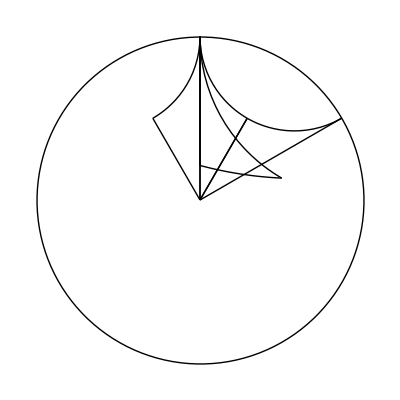

```mathematica
showChambers[triangle[2,6,Infinity],words[triangle[2,6,Infinity],1],Red]
```

### Group Data

```mathematica
chamberVertices[typeA[3],""]={{0,0,0},{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}};
chamberVertices[typeB[3],""]={{0,0,0},{0,0,1},{0,-1,1},{-1,-1,1}};
chamberVertices[H3,""]={{0,0,0},{0,0,1.615},{1,0,1.615},{1,Tan[Pi/5],1.615}};
chamberVertices[M_,""]:={{0,0},{0,1},{Tan[Pi/M[[1]][[2]]],1}}/;rank[M]==2
chamberVertices[ST,""]={{0.93,0.03},{0.03,0.03},{0.03,0.93}};
chamberVertices[S,""]={{0.03,0.03},{0.03,0.97},{0.97,0.97},{0.97,0.03}};
chamberVertices[HT,""]={{0.03,0.03},{0.93,0.03},{0.03,1.61}};
chamberVertices[TT,""]={{0.03,0.03},{0.5,0.84},{0.97,0.03}};
chamberVertices[triangle[2,6,Infinity],""]={{0,0},{0,1},{Cos[Pi/3]/Sqrt[3],Sin[Pi/3]/Sqrt[3]}};
```

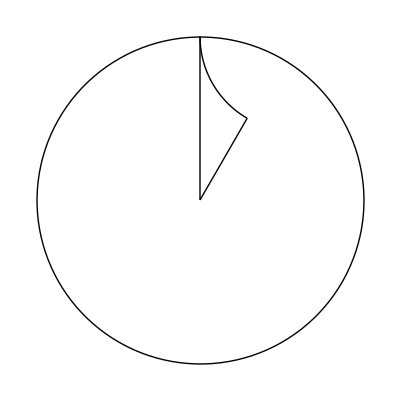

```mathematica
Show[Graphics[Circle[{0,0},1]],chamber[triangle[2,6,Infinity],""]]
```

### Hyperplanes

```mathematica
zeroVector[M_]:=Module[{r,e,n},
r=rank[M];
e=If[sphericalQ[M],0,If[Or[euclideanQ[M],hyperbolicQ[M]],1,0]];
n=r-e;
Table[0,{k,1,n}]
]
normal[M_,r_]:=transformation[M,conjugatingElement[r],normal[M,centralGenerator[r]]]-transformation[M,conjugatingElement[r],zeroVector[M]]/;StringLength[r]>1
basePoint[M_,r_]:=zeroVector[M]/;sphericalQ[M]
basePoint[M_,r_]:=transformation[M,conjugatingElement[r],basePoint[M,centralGenerator[r]]]/;euclideanQ[M]&&StringLength[r]>1
hyperplane[M_,r_]:=Hyperplane[normal[M,r],basePoint[M,r]]
showHyperplanes[M_,rList_List]:=If[Length[basePoint[M,"1"]]==2,Graphics[hyperplane[M,#]&/@rList],Graphics3D[hyperplane[M,#]&/@rList]]
```

#### Group Data

Type A[3]

```mathematica
normal[typeA[3],"1"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{0,-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"2"]:=Cross[{0,0,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
normal[typeA[3],"3"]:=Cross[{0,-1,Tan[ArcCos[1/3]/2]},{1/Tan[Pi/6],-1,Tan[ArcCos[1/3]/2]}]
```

Type B[3]

```mathematica
normal[typeB[3],"1"]:=Cross[{0,-1,1},{-1,-1,1}]
normal[typeB[3],"2"]:=Cross[{0,0,1},{-1,-1,1}]
normal[typeB[3],"3"]:=Cross[{0,0,1},{0,-1,1}]
```

H3

```mathematica
normal[H3,"1"]:=Cross[{1,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"2"]:=Cross[{0,0,1.615},{1,Tan[Pi/5],1.615}]
normal[H3,"3"]:=Cross[{0,0,1.615},{1,0,1.615}]
```

I2[m]

```mathematica
normal[M_,"1"]:={1,-Tan[Pi/M[[1]][[2]]]}/;rank[M]==2
normal[M_,"2"]:={1,0}/;rank[M]==2
```

ST

```mathematica
normal[ST,"1"]:={1,1}
normal[ST,"2"]:={1,0}
normal[ST,"3"]:={0,1}
basePoint[ST,"1"]:={1,0}
basePoint[ST,"2"]:={0,0}
basePoint[ST,"3"]:={0,0}
```

S

```mathematica
normal[S,"1"]:={1,0}
normal[S,"2"]:={1,0}
normal[S,"3"]:={0,1}
normal[S,"4"]:={0,1}
basePoint[S,"1"]:={0,0}
basePoint[S,"2"]:={1,0}
basePoint[S,"3"]:={0,0}
basePoint[S,"4"]:={0,1}
```

HT

```mathematica
normal[HT,"1"]:={Sqrt[3],1}
normal[HT,"2"]:={1,0}
normal[HT,"3"]:={0,1}
basePoint[HT,"1"]:={1,0}
basePoint[HT,"2"]:={0,0}
basePoint[HT,"3"]:={0,0}
```

TT

```mathematica
normal[TT,"1"]:={Sqrt[3],-1}
normal[TT,"2"]:={Sqrt[3],1}
normal[TT,"3"]:={0,1}
basePoint[TT,"1"]:={0,0}
basePoint[TT,"2"]:={1,0}
basePoint[TT,"3"]:={0,0}
```

### Visualisation

#### Chambers

```mathematica
showLengthIdeal[M_,k_]:=Show[Table[showChambers[M,lengthIdeal[M,k-i],Hue[i/k]],{i,0,k}]]
showBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],bruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showLeftBruhatIdeal[M_,""]:=showChambers[M,{""},Black]
showLeftBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],leftBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showRightBruhatIdeal[M_,w_]:=Show[Table[showChambers[M,Intersection[lengthIdeal[M,coxeterLength[M,w]-i],rightBruhatIdeal[M,w]],Hue[i/coxeterLength[M,w]]],{i,0,coxeterLength[M,w]}],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothness[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Red],showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showSmoothChambers[M_,k_]:=Show[showChambers[M,smoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothChambers[M_,k_]:=Show[showChambers[M,nonSmoothElements[M,k],Green],If[Length[chamberVertices[M,""][[1]]]==2,Graphics[{Black,chamber[M,""]}],Graphics3D[{Black,chamber[M,""]}]]]
showNonSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@nonSmoothElements[M,k],ImageSize->Large]
showSmoothBruhatIdeals[M_,k_]:=GraphicsRow[showBruhatIdeal[M,#]&/@smoothElements[M,k],ImageSize->Large]
showLeftAndInvertedLeftBruhatIdeal[M_,""]:=showChambers[M,{"",longestElement[M]},Red]/;size[M]<Infinity
showLeftAndInvertedLeftBruhatIdeal[M_,w_]:=showChambers[M,deleteRepeatedElements[M,Union[leftBruhatIdeal[M,w],invertedLeftBruhatIdeal[M,w]]],Red]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,""]:=showChambers[M,{""},Blue]/;size[M]<Infinity
showLeftAndInvertedBruhatMinusLeftIdeal[M_,w_]:=showChambers[M,Union[leftBruhatIdeal[M,w],invertedBruhatIdealMinusLeft[M,w]],Blue]/;size[M]<Infinity
```

```mathematica
showLengthIdeal[S,1]
```

-Graphics3D-

#### Chambers Examples

```mathematica
GraphicsRow[{showLengthIdeal[typeA[3],6],showLengthIdeal[typeB[3],9],showLengthIdeal[H3,15]},Frame->False,ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{showSmoothness[typeA[3],6],showSmoothness[typeB[3],9],showSmoothness[H3,15]},Frame->False,ImageSize->Large]
```

-Graphics-

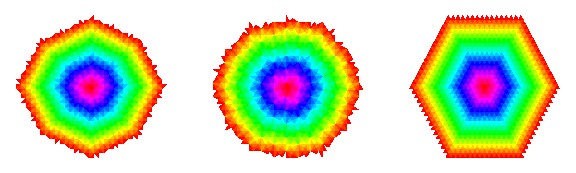

```mathematica
GraphicsRow[{showLengthIdeal[ST,30],showLengthIdeal[HT,30],showLengthIdeal[TT,30]},ImageSize->Large]
```

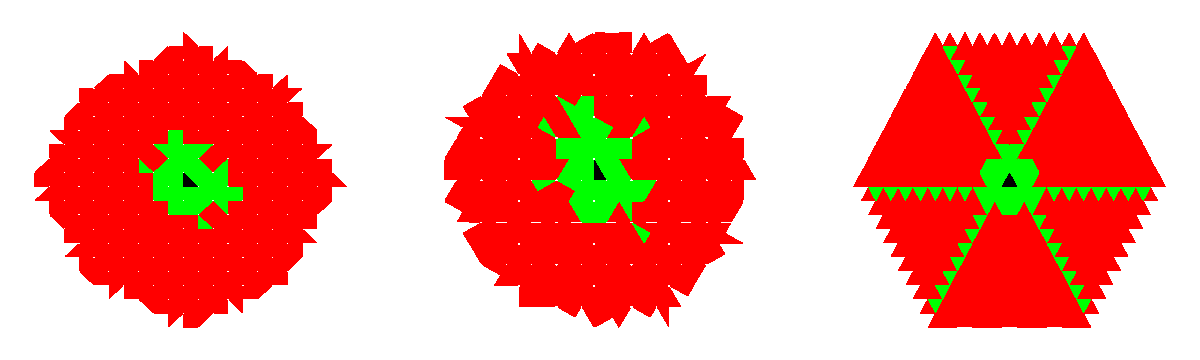

```mathematica
GraphicsRow[{showSmoothness[ST,20],showSmoothness[HT,20],showSmoothness[TT,20]},ImageSize->Large]
```

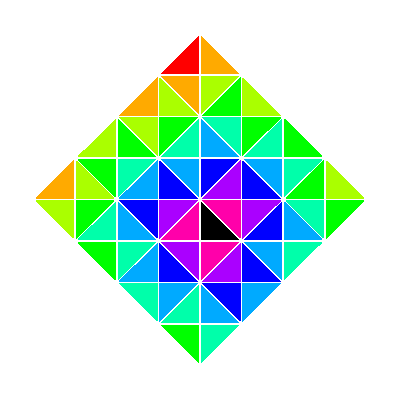
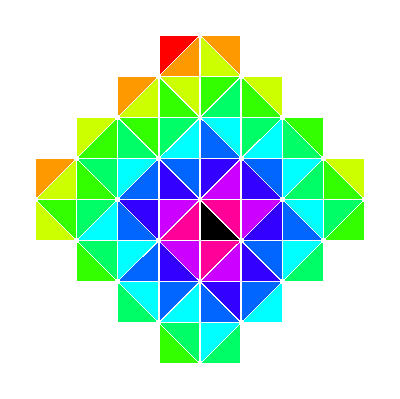
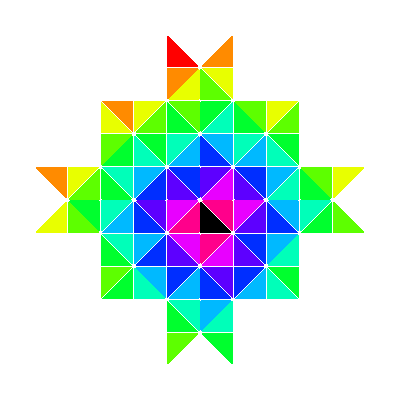
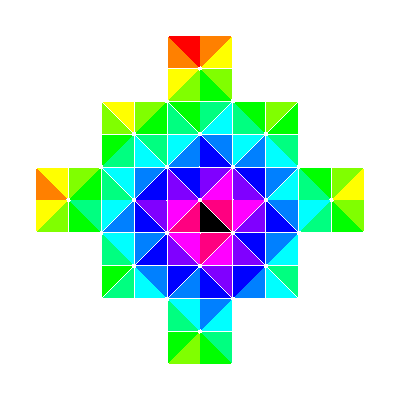
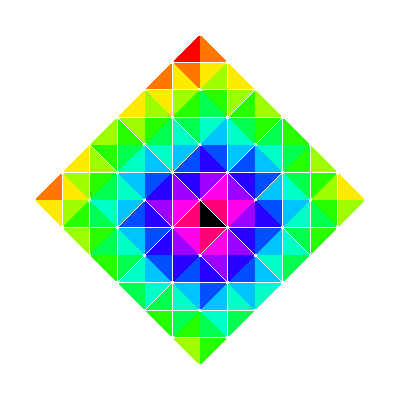
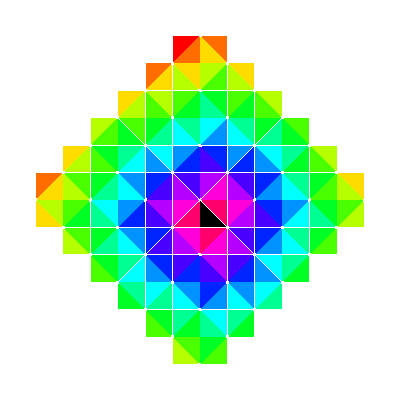
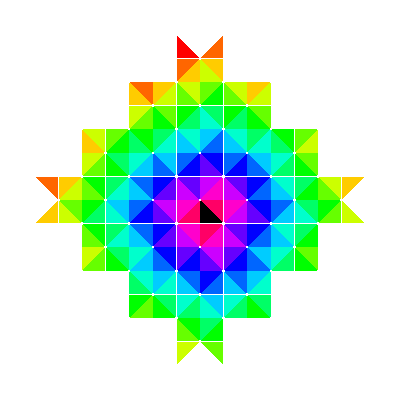
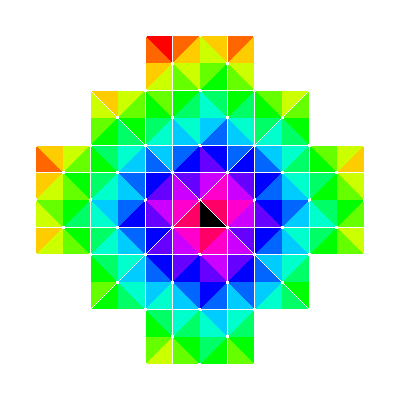

```mathematica
showNonSmoothBruhatIdeals[ST,15]
```

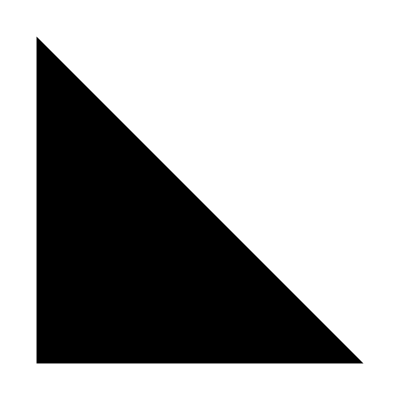
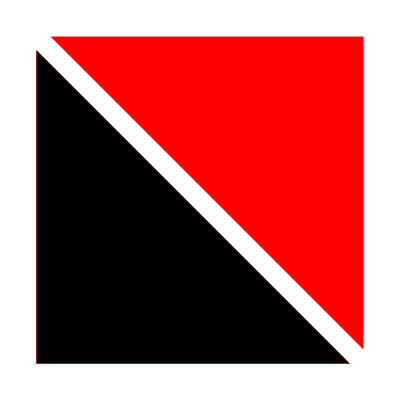
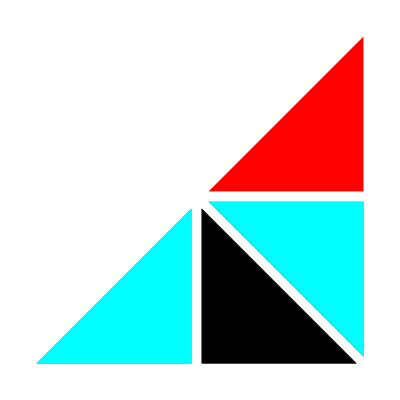
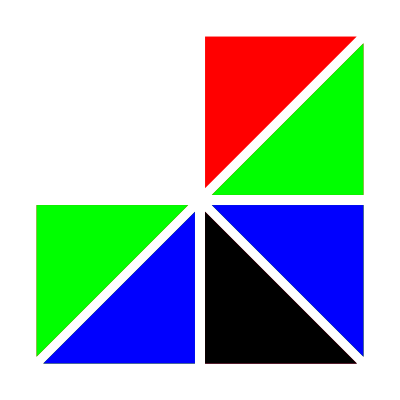
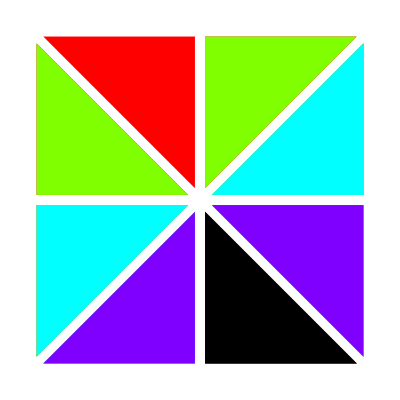
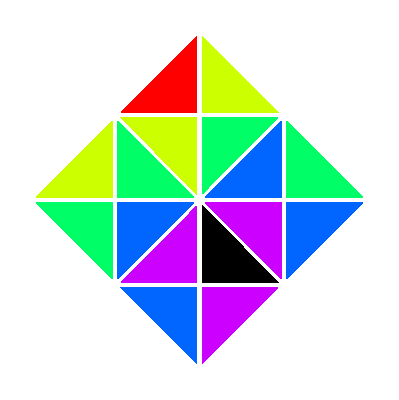
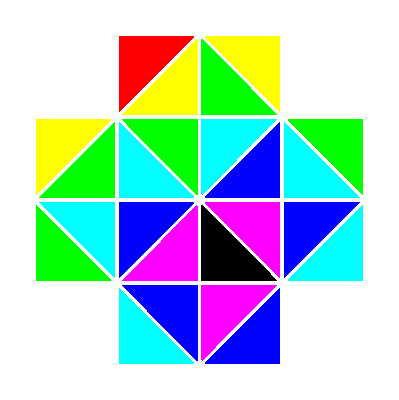
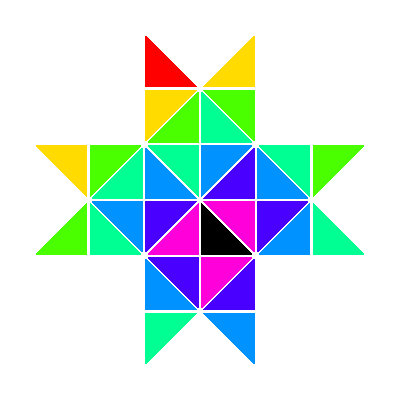

```mathematica
showSmoothBruhatIdeals[ST,15]
```

#### Hyperplane Arrangements

```mathematica
showHyperplanes[M_,k_]:=showHyperplanes[M,DeleteDuplicates[Flatten[inv[M,#]&/@Complement[lengthIdeal[M,k],lengthIdeal[M,k-1]]]]]
showInvArrangement[M_,""]:=showChambers[M,{""},Black]
showInvArrangement[M_,w_]:=Show[showHyperplanes[M,inv[M,w]],showChambers[M,{""},Black],showChambers[M,{w},Red]]
showInvArrangementBruhat[M_,w_]:=Show[showBruhatIdeal[M,w],showInvArrangement[M,w]]
showInvArrangementLeftBruhat[M_,w_]:=Show[showLeftBruhatIdeal[M,w],showInvArrangement[M,w]]
```

#### Hyperplane Arrangements Examples

```mathematica
GraphicsRow[{showInvArrangement[ST,"123123121"],showInvArrangementBruhat[ST,"123123121"],showInvArrangementLeftBruhat[ST,"123123121"]}]
```

-Graphics-

```mathematica
Show[showBruhatIdeal[TT,"123123123123123"],showHyperplanes[TT,inv[TT,"123123123123123"]]]
```

-Graphics-

```mathematica
{#,poincarePoly[H3,#,q],Show[Graphics3D[Sphere[{0,0,0},1],ImageSize->Large],showInvArrangement[H3,#],showLeftBruhatIdeal[H3,#],showChambers[H3,{"123123123123123"},Blue]]}&/@smoothElements[H3,15]
```

{{,1,-Graphics3D-},{1,1+q,-Graphics3D-},{12,1+2 q+q^2,-Graphics3D-},{121,1+2 q+2 q^2+q^3,-Graphics3D-},{1213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12132,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{121321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{121321321321323,1+3 q+5 q^2+7 q^3+9 q^4+11 q^5+12 q^6+12 q^7+12 q^8+12 q^9+11 q^10+9 q^11+7 q^12+5 q^13+3 q^14+q^15,-Graphics3D-},{1213213232,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{121323,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{1213232,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{123,1+3 q+3 q^2+q^3,-Graphics3D-},{1232,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12323,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{123232,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{13,1+2 q+q^2,-Graphics3D-},{132,1+3 q+3 q^2+q^3,-Graphics3D-},{1321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13213232,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{1323,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13232,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2,1+q,-Graphics3D-},{21,1+2 q+q^2,-Graphics3D-},{213,1+3 q+3 q^2+q^3,-Graphics3D-},{21321,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{213213232,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{23,1+2 q+q^2,-Graphics3D-},{232,1+2 q+2 q^2+q^3,-Graphics3D-},{2321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{23213,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2321321,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{23213213,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{232132132,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{2321321321,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2321321323,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2323,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{23232,1+2 q+2 q^2+2 q^3+2 q^4+q^5,-Graphics3D-},{232321,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{3,1+q,-Graphics3D-},{32,1+2 q+q^2,-Graphics3D-},{321,1+3 q+3 q^2+q^3,-Graphics3D-},{3213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{321321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{323,1+2 q+2 q^2+q^3,-Graphics3D-},{3232,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{32321,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-}}

```mathematica
{#,poincarePoly[H3,#,q],Show[Graphics3D[Sphere[{0,0,0},1],ImageSize->Large],showInvArrangement[H3,#],showLeftAndInvertedLeftBruhatIdeal[H3,#],showChambers[H3,{"123123123123123"},Blue]]}&/@smoothElements[H3,15]
```

{{,1,-Graphics3D-},{1,1+q,-Graphics3D-},{12,1+2 q+q^2,-Graphics3D-},{121,1+2 q+2 q^2+q^3,-Graphics3D-},{1213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12132,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{121321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{121321321321323,1+3 q+5 q^2+7 q^3+9 q^4+11 q^5+12 q^6+12 q^7+12 q^8+12 q^9+11 q^10+9 q^11+7 q^12+5 q^13+3 q^14+q^15,-Graphics3D-},{1213213232,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{121323,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{1213232,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{123,1+3 q+3 q^2+q^3,-Graphics3D-},{1232,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12323,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{123232,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{13,1+2 q+q^2,-Graphics3D-},{132,1+3 q+3 q^2+q^3,-Graphics3D-},{1321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13213232,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{1323,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13232,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2,1+q,-Graphics3D-},{21,1+2 q+q^2,-Graphics3D-},{213,1+3 q+3 q^2+q^3,-Graphics3D-},{21321,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{213213232,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{23,1+2 q+q^2,-Graphics3D-},{232,1+2 q+2 q^2+q^3,-Graphics3D-},{2321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{23213,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2321321,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{23213213,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{232132132,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{2321321321,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2321321323,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2323,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{23232,1+2 q+2 q^2+2 q^3+2 q^4+q^5,-Graphics3D-},{232321,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{3,1+q,-Graphics3D-},{32,1+2 q+q^2,-Graphics3D-},{321,1+3 q+3 q^2+q^3,-Graphics3D-},{3213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{321321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{323,1+2 q+2 q^2+q^3,-Graphics3D-},{3232,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{32321,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-}}

```mathematica
{#,poincarePoly[H3,#,q],Show[Graphics3D[Sphere[{0,0,0},1],ImageSize->Large],showInvArrangement[H3,#],showLeftAndInvertedBruhatMinusLeftIdeal[H3,#],showChambers[H3,{"123123123123123"},Black]]}&/@smoothElements[H3,15]
```

{{,1,-Graphics3D-},{1,1+q,-Graphics3D-},{12,1+2 q+q^2,-Graphics3D-},{121,1+2 q+2 q^2+q^3,-Graphics3D-},{1213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12132,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{121321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{121321321321323,1+3 q+5 q^2+7 q^3+9 q^4+11 q^5+12 q^6+12 q^7+12 q^8+12 q^9+11 q^10+9 q^11+7 q^12+5 q^13+3 q^14+q^15,-Graphics3D-},{1213213232,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{121323,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{1213232,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{123,1+3 q+3 q^2+q^3,-Graphics3D-},{1232,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{12323,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{123232,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{13,1+2 q+q^2,-Graphics3D-},{132,1+3 q+3 q^2+q^3,-Graphics3D-},{1321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13213232,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{1323,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{13232,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2,1+q,-Graphics3D-},{21,1+2 q+q^2,-Graphics3D-},{213,1+3 q+3 q^2+q^3,-Graphics3D-},{21321,1+3 q+5 q^2+5 q^3+3 q^4+q^5,-Graphics3D-},{213213232,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{23,1+2 q+q^2,-Graphics3D-},{232,1+2 q+2 q^2+q^3,-Graphics3D-},{2321,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{23213,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-},{2321321,1+3 q+5 q^2+6 q^3+6 q^4+5 q^5+3 q^6+q^7,-Graphics3D-},{23213213,1+3 q+5 q^2+7 q^3+8 q^4+7 q^5+5 q^6+3 q^7+q^8,-Graphics3D-},{232132132,1+3 q+5 q^2+7 q^3+9 q^4+9 q^5+7 q^6+5 q^7+3 q^8+q^9,-Graphics3D-},{2321321321,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2321321323,1+3 q+5 q^2+7 q^3+9 q^4+10 q^5+9 q^6+7 q^7+5 q^8+3 q^9+q^10,-Graphics3D-},{2323,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{23232,1+2 q+2 q^2+2 q^3+2 q^4+q^5,-Graphics3D-},{232321,1+3 q+4 q^2+4 q^3+4 q^4+3 q^5+q^6,-Graphics3D-},{3,1+q,-Graphics3D-},{32,1+2 q+q^2,-Graphics3D-},{321,1+3 q+3 q^2+q^3,-Graphics3D-},{3213,1+3 q+4 q^2+3 q^3+q^4,-Graphics3D-},{321321,1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6,-Graphics3D-},{323,1+2 q+2 q^2+q^3,-Graphics3D-},{3232,1+2 q+2 q^2+2 q^3+q^4,-Graphics3D-},{32321,1+3 q+4 q^2+4 q^3+3 q^4+q^5,-Graphics3D-}}

## 2.5 Factorisation

### Polynomial Manipulation

```mathematica
zeroPolynomialQ[poly_,q_]:=CoefficientList[poly,q]=={}
polynomialDividesQ[poly1_,poly2_,q_]:=If[zeroPolynomialQ[PolynomialRemainder[poly1,poly2,q],q],True,False]
divideMult[m_,n_]:=Floor[m/n]
factorMults[factors1_,fac2_]:=divideMult[Select[factors1,#[[1]]==fac2[[1]]&][[1]][[2]],fac2[[2]]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=0/;Not[polynomialDividesQ[poly1,poly2,q]]
polynomialDividesMultiplicity[poly1_,poly2_,q_]:=Module[{factors1,factors2,mult},
factors1=#&/@Complement[FactorList[poly1],{{1,1}}];
factors2=#&/@Complement[FactorList[poly2],{{1,1}}];
mult=factorMults[factors1,#]&/@factors2;
Min[mult]
]/;polynomialDividesQ[poly1,poly2,q]
removePolynomialFactors[poly1_,poly2_,q_]:=
Simplify[poly1/(poly2^polynomialDividesMultiplicity[poly1,poly2,q])]
removePolynomialFactors[poly1_,polyList_List,q_]:=
Simplify[poly1/Fold[Times,#^polynomialDividesMultiplicity[poly1,#,q]]&/@polyList]
```

### Quantum Factorisation

```mathematica
quantumPoly[k_,q_]:=Total[Table[( q)^i,{i,0,k}]]
quantumPolyQ[1,q_]:=True
quantumPolyQ[poly_,q_]:=CoefficientList[poly,q]==CoefficientList[quantumPoly[Max[1,Exponent[poly,q]],q],q]
quantumFactorQ[poly_,0,q_]:=True
quantumFactorQ[poly_,k_,q_]:=polynomialDividesQ[poly,quantumPoly[k,q],q]
quantumFactorsQ[poly_,q_]:=Fold[Or,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}]]
removeQuantumFactors[poly_,q_]:=removePolynomialFactors[poly,Table[quantumFactorQ[poly,k,q],{k,1,Max[1,Exponent[poly,q]]}],q]
quantumFactorList[poly_,q_]:=Module[{d},
d=Max[1,Exponent[poly,q]];
Select[Table[{{k,q},polynomialDividesMultiplicity[poly,quantumPoly[k,q],q]},{k,1,d}],#[[2]]≥ 1&]
]
quantumFactorisation[poly_,q_]:=FactorList[poly]/;Not[quantumFactorsQ[poly,q]]
quantumFactorisation[poly_,q_]:=Module[{qfl,k,n,newP},
qfl=quantumFactorList[poly,q];
k=Max[#[[1]][[1]]&/@qfl];
n=polynomialDividesMultiplicity[poly,quantumPoly[k,q],q];
newP=removePolynomialFactors[poly,quantumPoly[k,q],q];
Join[quantumFactorisation[newP,q],{{quantumPoly[k,q],n}}]
]/;quantumFactorsQ[poly,q]
quantumFactorisationQ[poly_,q_]:=Fold[And,quantumPolyQ[#[[1]],q]&/@quantumFactorisation[poly,q]]
quantumFactorisationQ[M_List,w_String]:=quantumFactorisationQ[poincarePoly[M,w,q],q]
quantumFactorisationQ[M_List,wList_List]:=Fold[And,quantumFactorisationQ[poincarePoly[M,#,q],q]&/@wList]
quantumExponents[poly_,q_]:=If[quantumFactorisationQ[poly,q],Drop[Flatten[Table[Exponent[#[[1]],q],{i,1,#[[2]]}]&/@quantumFactorisation[poly,q]],1],{}]
quantumExponents[M_List,w_String]:=quantumExponents[poincarePoly[M,w,q],q]
quantumExponents[M_List,wList_List]:={#,quantumExponents[poincarePoly[M,#,q],q]}&/@wList
```

### q-Factorisation Property

```mathematica
qFactorisationProperty[M_,k_]:=
qFactorisationProperty[M,k]={#,quantumFactorisationQ[M,#]}&/@smoothElements[M,k]
qFactorisationPropertyQ[M_,k_]:=Fold[And,#[[2]]&/@qFactorisationProperty[M,k]]
qFactorisationPropertyQ[M_]:=qFactorisationPropertyQ[M,maxLength[M]]
```

H3

```mathematica
qFactorisationPropertyQ[H3]
```

True

H4

```mathematica
qFactorisationPropertyQ[H4,15]
```

True

F4

```mathematica
qFactorisationPropertyQ[F4,24]
```

True

### Visualisation

```mathematica
lexOrder[list1_,list2_]:=If[list1[[1]]<list2[[1]],True,If[list1[[1]]==list2[[1]],lexOrder[Drop[list1,1],Drop[list2,1]],False]]
lexOrder[{},list_]:=True
lexOrder[list_,{}]:=False/;Not[list=={}]
quantumExponentsVisualisation[M_,k_]:=Sort[{#,quantumExponents[poincarePoly[M,#,q],q],showInvArrangement[M,#]}&/@smoothElements[M,k],lexOrder[#1[[2]],#2[[2]]]&]
```

```mathematica
smoothElements[S,15]
```

$Aborted

```mathematica
quantumExponentsVisualisation[S,15]
```

$Aborted

```mathematica
Sort[{#,quantumExponents[poincarePoly[S,#,q],q]}&/@words[S,10],lexOrder[#1[[2]],#2[[2]]]&]
```

{{,{}},{1,{1}},{2,{1}},{3,{1}},{4,{1}},{12,{1,1}},{13,{1,1}},{14,{1,1}},{21,{1,1}},{23,{1,1}},{24,{1,1}},{34,{1,1}},{43,{1,1}},{123,{1,1,1}},{124,{1,1,1}},{134,{1,1,1}},{143,{1,1,1}},{213,{1,1,1}},{214,{1,1,1}},{234,{1,1,1}},{243,{1,1,1}},{1234,{1,1,1,1}},{1243,{1,1,1,1}},{2134,{1,1,1,1}},{2143,{1,1,1,1}},{12134,{1,1,1,2}},{12143,{1,1,1,2}},{12343,{1,1,1,2}},{12434,{1,1,1,2}},{21234,{1,1,1,2}},{21243,{1,1,1,2}},{21343,{1,1,1,2}},{21434,{1,1,1,2}},{121234,{1,1,1,3}},{121243,{1,1,1,3}},{123434,{1,1,1,3}},{124343,{1,1,1,3}},{212134,{1,1,1,3}},{212143,{1,1,1,3}},{213434,{1,1,1,3}},{214343,{1,1,1,3}},{1212134,{1,1,1,4}},{1212143,{1,1,1,4}},{1234343,{1,1,1,4}},{1243434,{1,1,1,4}},{2121234,{1,1,1,4}},{2121243,{1,1,1,4}},{2134343,{1,1,1,4}},{2143434,{1,1,1,4}},{12121234,{1,1,1,5}},{12121243,{1,1,1,5}},{12343434,{1,1,1,5}},{12434343,{1,1,1,5}},{21212134,{1,1,1,5}},{21212143,{1,1,1,5}},{21343434,{1,1,1,5}},{21434343,{1,1,1,5}},{121212134,{1,1,1,6}},{121212143,{1,1,1,6}},{123434343,{1,1,1,6}},{124343434,{1,1,1,6}},{212121234,{1,1,1,6}},{212121243,{1,1,1,6}},{213434343,{1,1,1,6}},{214343434,{1,1,1,6}},{1212121234,{1,1,1,7}},{1212121243,{1,1,1,7}},{1234343434,{1,1,1,7}},{1243434343,{1,1,1,7}},{2121212134,{1,1,1,7}},{2121212143,{1,1,1,7}},{2134343434,{1,1,1,7}},{2143434343,{1,1,1,7}},{1213,{1,1,2}},{1214,{1,1,2}},{1343,{1,1,2}},{1434,{1,1,2}},{2123,{1,1,2}},{2124,{1,1,2}},{2343,{1,1,2}},{2434,{1,1,2}},{121343,{1,1,2,2}},{121434,{1,1,2,2}},{212343,{1,1,2,2}},{212434,{1,1,2,2}},{1212343,{1,1,2,3}},{1212434,{1,1,2,3}},{1213434,{1,1,2,3}},{1214343,{1,1,2,3}},{2121343,{1,1,2,3}},{2121434,{1,1,2,3}},{2123434,{1,1,2,3}},{2124343,{1,1,2,3}},{12121343,{1,1,2,4}},{12121434,{1,1,2,4}},{12134343,{1,1,2,4}},{12143434,{1,1,2,4}},{21212343,{1,1,2,4}},{21212434,{1,1,2,4}},{21234343,{1,1,2,4}},{21243434,{1,1,2,4}},{121212343,{1,1,2,5}},{121212434,{1,1,2,5}},{121343434,{1,1,2,5}},{121434343,{1,1,2,5}},{212121343,{1,1,2,5}},{212121434,{1,1,2,5}},{212343434,{1,1,2,5}},{212434343,{1,1,2,5}},{1212121343,{1,1,2,6}},{1212121434,{1,1,2,6}},{1213434343,{1,1,2,6}},{1214343434,{1,1,2,6}},{2121212343,{1,1,2,6}},{2121212434,{1,1,2,6}},{2123434343,{1,1,2,6}},{2124343434,{1,1,2,6}},{12123,{1,1,3}},{12124,{1,1,3}},{13434,{1,1,3}},{14343,{1,1,3}},{21213,{1,1,3}},{21214,{1,1,3}},{23434,{1,1,3}},{24343,{1,1,3}},{12123434,{1,1,3,3}},{12124343,{1,1,3,3}},{21213434,{1,1,3,3}},{21214343,{1,1,3,3}},{121213434,{1,1,3,4}},{121214343,{1,1,3,4}},{121234343,{1,1,3,4}},{121243434,{1,1,3,4}},{212123434,{1,1,3,4}},{212124343,{1,1,3,4}},{212134343,{1,1,3,4}},{212143434,{1,1,3,4}},{1212123434,{1,1,3,5}},{1212124343,{1,1,3,5}},{1212343434,{1,1,3,5}},{1212434343,{1,1,3,5}},{2121213434,{1,1,3,5}},{2121214343,{1,1,3,5}},{2121343434,{1,1,3,5}},{2121434343,{1,1,3,5}},{121213,{1,1,4}},{121214,{1,1,4}},{134343,{1,1,4}},{143434,{1,1,4}},{212123,{1,1,4}},{212124,{1,1,4}},{234343,{1,1,4}},{243434,{1,1,4}},{1212134343,{1,1,4,4}},{1212143434,{1,1,4,4}},{2121234343,{1,1,4,4}},{2121243434,{1,1,4,4}},{1212123,{1,1,5}},{1212124,{1,1,5}},{1343434,{1,1,5}},{1434343,{1,1,5}},{2121213,{1,1,5}},{2121214,{1,1,5}},{2343434,{1,1,5}},{2434343,{1,1,5}},{12121213,{1,1,6}},{12121214,{1,1,6}},{13434343,{1,1,6}},{14343434,{1,1,6}},{21212123,{1,1,6}},{21212124,{1,1,6}},{23434343,{1,1,6}},{24343434,{1,1,6}},{121212123,{1,1,7}},{121212124,{1,1,7}},{134343434,{1,1,7}},{143434343,{1,1,7}},{212121213,{1,1,7}},{212121214,{1,1,7}},{234343434,{1,1,7}},{243434343,{1,1,7}},{1212121213,{1,1,8}},{1212121214,{1,1,8}},{1343434343,{1,1,8}},{1434343434,{1,1,8}},{2121212123,{1,1,8}},{2121212124,{1,1,8}},{2343434343,{1,1,8}},{2434343434,{1,1,8}},{121,{1,2}},{212,{1,2}},{343,{1,2}},{434,{1,2}},{1212,{1,3}},{2121,{1,3}},{3434,{1,3}},{4343,{1,3}},{12121,{1,4}},{21212,{1,4}},{34343,{1,4}},{43434,{1,4}},{121212,{1,5}},{212121,{1,5}},{343434,{1,5}},{434343,{1,5}},{1212121,{1,6}},{2121212,{1,6}},{3434343,{1,6}},{4343434,{1,6}},{12121212,{1,7}},{21212121,{1,7}},{34343434,{1,7}},{43434343,{1,7}},{121212121,{1,8}},{212121212,{1,8}},{343434343,{1,8}},{434343434,{1,8}},{1212121212,{1,9}},{2121212121,{1,9}},{3434343434,{1,9}},{4343434343,{1,9}}}

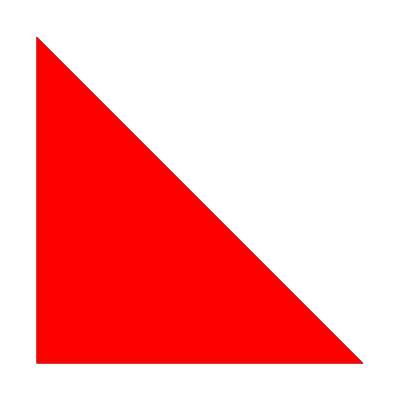
{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{2313,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{3123,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{13123,{1,1,3},-Graphics-},{21313,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{313,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{121231,{1,2,3},-Graphics-},{121313,{1,2,3},-Graphics-},{123121,{1,2,3},-Graphics-},{131231,{1,2,3},-Graphics-},{1212,{1,3},-Graphics-},{1313,{1,3},-Graphics-},{1212312,{1,3,3},-Graphics-},{1212313,{1,3,3},-Graphics-},{1312312,{1,3,3},-Graphics-},{1312313,{1,3,3},-Graphics-},{2123121,{1,3,3},-Graphics-},{3121313,{1,3,3},-Graphics-},{12123121,{1,3,4},-Graphics-},{13121313,{1,3,4},-Graphics-}}

```mathematica
quantumExponentsVisualisation[ST,15]
```

```mathematica
quantumExponentsVisualisation[HT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2123,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2312,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{12123,{1,1,3},-Graphics-},{21213,{1,1,3},-Graphics-},{23121,{1,1,3},-Graphics-},{31212,{1,1,3},-Graphics-},{121213,{1,1,4},-Graphics-},{212123,{1,1,4},-Graphics-},{231212,{1,1,4},-Graphics-},{312121,{1,1,4},-Graphics-},{1212123,{1,1,5},-Graphics-},{2312121,{1,1,5},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{212,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{131212,{1,2,3},-Graphics-},{131213,{1,2,3},-Graphics-},{212131,{1,2,3},-Graphics-},{1212131,{1,2,4},-Graphics-},{1312121,{1,2,4},-Graphics-},{12121231,{1,2,5},-Graphics-},{12312121,{1,2,5},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{121212312,{1,3,5},-Graphics-},{212312121,{1,3,5},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{1212123121,{1,4,5},-Graphics-},{1212312121,{1,4,5},-Graphics-},{121212,{1,5},-Graphics-},{12121231212,{1,5,5},-Graphics-},{12121231213,{1,5,5},-Graphics-},{13121231212,{1,5,5},-Graphics-},{21212312121,{1,5,5},-Graphics-},{121212312121,{1,5,6},-Graphics-}}

```mathematica
quantumExponentsVisualisation[TT,15]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{3,{1},-Graphics-},{12,{1,1},-Graphics-},{13,{1,1},-Graphics-},{21,{1,1},-Graphics-},{23,{1,1},-Graphics-},{31,{1,1},-Graphics-},{32,{1,1},-Graphics-},{123,{1,1,1},-Graphics-},{132,{1,1,1},-Graphics-},{213,{1,1,1},-Graphics-},{231,{1,1,1},-Graphics-},{312,{1,1,1},-Graphics-},{321,{1,1,1},-Graphics-},{1213,{1,1,2},-Graphics-},{1232,{1,1,2},-Graphics-},{1312,{1,1,2},-Graphics-},{2131,{1,1,2},-Graphics-},{2321,{1,1,2},-Graphics-},{3121,{1,1,2},-Graphics-},{121,{1,2},-Graphics-},{131,{1,2},-Graphics-},{232,{1,2},-Graphics-},{12131,{1,2,2},-Graphics-},{12132,{1,2,2},-Graphics-},{13121,{1,2,2},-Graphics-},{13123,{1,2,2},-Graphics-},{23121,{1,2,2},-Graphics-},{23213,{1,2,2},-Graphics-},{1213123,{2,2,3},-Graphics-},{1213213,{2,2,3},-Graphics-},{1312132,{2,2,3},-Graphics-},{1312312,{2,2,3},-Graphics-},{2312131,{2,2,3},-Graphics-},{2321321,{2,2,3},-Graphics-},{121312312,{2,3,4},-Graphics-},{121321321,{2,3,4},-Graphics-},{131213213,{2,3,4},-Graphics-},{131231231,{2,3,4},-Graphics-},{231213123,{2,3,4},-Graphics-},{232132132,{2,3,4},-Graphics-},{12131231231,{2,4,5},-Graphics-},{12132132132,{2,4,5},-Graphics-},{13121321321,{2,4,5},-Graphics-},{13123123123,{2,4,5},-Graphics-},{23121312312,{2,4,5},-Graphics-},{23213213213,{2,4,5},-Graphics-},{1213123123123,{2,5,6},-Graphics-},{1213213213213,{2,5,6},-Graphics-},{1312132132132,{2,5,6},-Graphics-},{1312312312312,{2,5,6},-Graphics-},{2312131231231,{2,5,6},-Graphics-},{2321321321321,{2,5,6},-Graphics-},{121312312312312,{2,6,7},-Graphics-},{121321321321321,{2,6,7},-Graphics-},{131213213213213,{2,6,7},-Graphics-},{131231231231231,{2,6,7},-Graphics-},{231213123123123,{2,6,7},-Graphics-},{232132132132132,{2,6,7},-Graphics-}}

```mathematica
quantumExponentsVisualisation[I2[12],12]
```

{{,{},-Graphics-},{1,{1},-Graphics-},{2,{1},-Graphics-},{12,{1,1},-Graphics-},{21,{1,1},-Graphics-},{121,{1,2},-Graphics-},{212,{1,2},-Graphics-},{1212,{1,3},-Graphics-},{2121,{1,3},-Graphics-},{12121,{1,4},-Graphics-},{21212,{1,4},-Graphics-},{121212,{1,5},-Graphics-},{212121,{1,5},-Graphics-},{1212121,{1,6},-Graphics-},{2121212,{1,6},-Graphics-},{12121212,{1,7},-Graphics-},{21212121,{1,7},-Graphics-},{121212121,{1,8},-Graphics-},{212121212,{1,8},-Graphics-},{1212121212,{1,9},-Graphics-},{2121212121,{1,9},-Graphics-},{12121212121,{1,10},-Graphics-},{21212121212,{1,10},-Graphics-},{121212121212,{1,11},-Graphics-}}

```mathematica
quantumFactorisation[poincarePoly[TT,"231213123123123",q],q]
```

{{1,1},{1+q+q^2,1},{1+q+q^2+q^3+q^4+q^5+q^6,1},{1+q+q^2+q^3+q^4+q^5+q^6+q^7,1}}

### Conjectures

```mathematica
letterCount[w_String]:=Sort[Union[makeList[w]]/.CharacterCounts[w]]
letterCounts[M_,w_String]:=DeleteDuplicates[letterCount[#]&/@reduce[M,w]]
centralGeneratorCount[M_,w_,s_]:=Length[Select[Sort[centralGenerator[#]&/@inv[M,w]],#==s&]]
centralGeneratorCounts[M_,w_]:=Sort[Select[Table[centralGeneratorCount[M,w,ToString[i]],{i,1,rank[M]}],Not[#==0]&]]
```

```mathematica
{#,letterCounts[TT,#][[1]]==quantumExponents[TT,#],centralGeneratorCounts[TT,#]==quantumExponents[TT,#]}&/@smoothElements[TT,15]
```

{{,True,True},{1,True,True},{12,True,True},{121,True,True},{1213,True,True},{12131,False,True},{1213123,True,False},{121312312,True,True},{12131231231,False,False},{1213123123123,False,False},{121312312312312,False,False},{12132,True,True},{1213213,True,True},{121321321,True,True},{12132132132,False,False},{1213213213213,False,False},{121321321321321,False,False},{123,True,True},{1232,True,True},{13,True,True},{131,True,True},{1312,True,True},{13121,False,True},{1312132,True,False},{131213213,True,True},{13121321321,False,False},{1312132132132,False,False},{131213213213213,False,False},{13123,True,True},{1312312,True,True},{131231231,True,True},{13123123123,False,False},{1312312312312,False,False},{131231231231231,False,False},{132,True,True},{2,True,True},{21,True,True},{213,True,True},{2131,True,True},{23,True,True},{231,True,True},{23121,True,True},{2312131,True,False},{231213123,False,False},{23121312312,False,False},{2312131231231,False,False},{231213123123123,False,False},{232,True,True},{2321,True,True},{23213,True,True},{2321321,True,True},{232132132,True,True},{23213213213,False,False},{2321321321321,False,False},{232132132132132,False,False},{3,True,True},{31,True,True},{312,True,True},{3121,True,True},{32,True,True},{321,True,True}}

```mathematica
centralGeneratorCounts[H3,#]&/@reduce[H3,"123123123123123"]
```

{{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8},{3,4,8}}

## 2.6 Bruhat ideals

```mathematica
coxeterElement[M_]:=makeString[Table[i,{i,1,rank[M]}]]
w[M_,k_]:=makeString[Flatten[Fold[Join,Table[makeList[coxeterElement[M]],{i,1,k}]]]]
```

Type A[5]

```mathematica
bruhatIdeal[typeA[5],w[typeA[5],3]]={"","4","5","1","3","2","54","34","45","24","14","43","15","35","23","13","12","32","21","25","234","354","543","254","154","454","345","324","134","343","245","145","435","243","143","124","432","214","235","135","125","325","215","232","132","213","121","321","123","2354","2324","2134","2343","4354","3543","3254","1354","3454","2543","1543","2454","1454","2154","1254","4543","3245","1345","3435","3243","1343","1324","3432","3214","2435","1435","1245","2432","1432","2143","1243","1214","4325","2145","2325","1325","2135","1215","2321","1321","2132","1232","1213","3215","1235","24354","23254","21354","23543","23243","21343","21324","23432","23214","43543","43254","34354","14354","32543","13543","32454","13454","32154","13254","24543","14543","21543","12543","21454","12454","12154","34543","32435","13435","13245","32432","13432","32143","13243","13214","24325","14325","21435","12435","12145","21432","12432","12143","23215","13215","21325","12325","12135","21321","12321","12132","34325","32145","324354","243543","243254","214354","232543","213543","232154","213254","232432","213432","232143","213243","213214","432543","343543","143543","343254","143254","134354","324543","134543","321543","132543","321454","132454","132154","214543","124543","121543","121454","324325","134325","321435","132435","132145","321432","132432","132143","214325","124325","121435","121432","213215","123215","121325","121321","3243543","3243254","3214354","2432543","2143543","2143254","2321543","2132543","2132154","2321432","2132432","2132143","3432543","1432543","1343543","1343254","3214543","1324543","1321543","1321454","1214543","3214325","1324325","1321435","1321432","1214325","1213215","32432543","32143543","32143254","21432543","21321543","21321432","13432543","13214543","13214325","321432543"};
```

Type B[5]

```mathematica
bruhatIdeal[typeB[5],w[typeB[5],3]]={"","5","4","1","3","2","54","45","15","35","25","43","14","34","23","13","12","32","21","24","545","543","454","154","354","254","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5435","4545","1545","3545","2545","4543","1543","3543","2543","4354","1454","3454","2354","1354","1254","3254","2154","2454","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","54354","45435","15435","35435","25435","43545","14545","34545","23545","13545","12545","32545","21545","24545","43543","14543","34543","23543","13543","12543","32543","21543","24543","43254","14354","34354","23454","13454","12454","32454","21454","23254","13254","21354","12154","32154","12354","24354","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","13214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","543545","454354","154354","354354","254354","435435","145435","345435","235435","135435","125435","325435","215435","245435","432545","143545","343545","234545","134545","124545","324545","214545","232545","132545","213545","121545","321545","123545","243545","432543","143543","343543","234543","134543","124543","324543","214543","232543","132543","213543","121543","321543","123543","243543","143254","343254","234354","134354","124354","324354","214354","232454","132454","213454","121454","132154","213254","123254","121354","321454","123454","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","132145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243254","232154","4543545","1543545","3543545","2543545","4354354","1454354","3454354","2354354","1354354","1254354","3254354","2154354","2454354","4325435","1435435","3435435","2345435","1345435","1245435","3245435","2145435","2325435","1325435","2135435","1215435","3215435","1235435","2435435","1432545","3432545","2343545","1343545","1243545","3243545","2143545","2324545","1324545","2134545","1214545","1321545","2132545","1232545","1213545","3214545","1234545","2432545","2321545","1432543","3432543","2343543","1343543","1243543","3243543","2143543","2324543","1324543","2134543","1214543","1321543","2132543","1232543","1213543","3214543","1234543","2343254","1343254","1243254","3243254","2143254","2324354","1324354","2134354","1214354","2321454","1321454","2132454","1232454","1213454","1232154","1213254","3214354","2132154","1234354","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","3214325","1234325","1232145","2432543","2321543","2321432","43543545","14543545","34543545","23543545","13543545","12543545","32543545","21543545","24543545","43254354","14354354","34354354","23454354","13454354","12454354","32454354","21454354","23254354","13254354","21354354","12154354","32154354","12354354","24354354","14325435","34325435","23435435","13435435","12435435","32435435","21435435","23245435","13245435","21345435","12145435","13215435","21325435","12325435","12135435","32145435","12345435","23432545","13432545","12432545","32432545","21432545","23243545","13243545","21343545","12143545","23214545","13214545","21324545","12324545","12134545","12321545","12132545","32143545","21321545","12343545","24325435","23215435","23432543","13432543","12432543","32432543","21432543","23243543","13243543","21343543","12143543","23214543","13214543","21324543","12324543","12134543","12321543","12132543","32143543","21321543","12343543","23243254","13243254","21343254","12143254","23214354","13214354","21324354","12324354","12134354","21321454","12132454","12132154","23214325","21324325","12324325","12134325","21321435","12321435","12132435","12132145","12321432","12132432","12132143","32143254","21321432","12343254","12321454","13214325","432543545","143543545","343543545","234543545","134543545","124543545","324543545","214543545","232543545","132543545","213543545","121543545","321543545","123543545","243543545","143254354","343254354","234354354","134354354","124354354","324354354","214354354","232454354","132454354","213454354","121454354","132154354","213254354","123254354","121354354","321454354","123454354","234325435","134325435","124325435","324325435","214325435","232435435","132435435","213435435","121435435","232145435","132145435","213245435","123245435","121345435","123215435","121325435","321435435","213215435","123435435","232432545","132432545","213432545","121432545","232143545","132143545","213243545","123243545","121343545","213214545","121324545","121321545","321432545","123432545","123214545","243254354","232154354","232432543","132432543","213432543","121432543","232143543","132143543","213243543","123243543","121343543","213214543","121324543","121321543","232143254","132143254","213243254","123243254","121343254","213214354","123214354","121324354","121321454","213214325","121324325","121321435","121321432","321432543","123432543","123214543","123214325","1432543545","3432543545","2343543545","1343543545","1243543545","3243543545","2143543545","2324543545","1324543545","2134543545","1214543545","1321543545","2132543545","1232543545","1213543545","3214543545","1234543545","2343254354","1343254354","1243254354","3243254354","2143254354","2324354354","1324354354","2134354354","1214354354","2321454354","1321454354","2132454354","1232454354","1213454354","1232154354","1213254354","3214354354","2132154354","1234354354","2324325435","1324325435","2134325435","1214325435","2321435435","1321435435","2132435435","1232435435","1213435435","2132145435","1213245435","1213215435","1321432545","2132432545","1232432545","1213432545","2132143545","1232143545","1213243545","1213214545","3214325435","1234325435","1232145435","2321432543","1321432543","2132432543","1232432543","1213432543","2132143543","1232143543","1213243543","1213214543","1232143254","1213243254","1213214354","1213214325","2432543545","2321543545","2321432545","2132143254","23432543545","13432543545","12432543545","32432543545","21432543545","23243543545","13243543545","21343543545","12143543545","23214543545","13214543545","21324543545","12324543545","12134543545","12321543545","12132543545","32143543545","21321543545","12343543545","23243254354","13243254354","21343254354","12143254354","23214354354","13214354354","21324354354","12324354354","12134354354","21321454354","12132454354","12132154354","23214325435","13214325435","21324325435","12324325435","12134325435","21321435435","12321435435","12132435435","12132145435","12321432545","12132432545","12132143545","32143254354","21321432545","12343254354","12321454354","21321432543","12321432543","12132432543","12132143543","12132143254","232432543545","132432543545","213432543545","121432543545","232143543545","132143543545","213243543545","123243543545","121343543545","213214543545","121324543545","121321543545","232143254354","132143254354","213243254354","123243254354","121343254354","213214354354","123214354354","121324354354","121321454354","213214325435","121324325435","121321435435","121321432545","321432543545","123432543545","123214543545","123214325435","121321432543","2321432543545","1321432543545","2132432543545","1232432543545","1213432543545","2132143543545","1232143543545","1213243543545","1213214543545","2132143254354","1232143254354","1213243254354","1213214354354","1213214325435","21321432543545","12321432543545","12132432543545","12132143543545","12132143254354","121321432543545"};
```

Type D[5]

```mathematica
bruhatIdeal[typeD[5],w[typeD[5],3]]={"","5","4","1","3","2","53","45","15","35","25","43","14","34","23","13","12","32","21","24","534","532","453","153","353","253","435","145","345","235","135","125","325","215","245","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","5324","4534","1534","3534","2534","4532","1532","3532","2532","4353","1453","3453","2353","1353","1253","3253","2153","2453","4325","1435","3435","2345","1345","1245","3245","2145","2325","1325","2135","1215","3215","1235","2435","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","53243","45324","15324","35324","25324","43534","14534","34534","23534","13534","12534","32534","21534","24534","43532","14532","34532","23532","13532","12532","32532","21532","24532","43253","14353","34353","23453","13453","12453","32453","21453","23253","13253","21353","12153","32153","12353","24353","14325","34325","23435","13435","12435","32435","21435","23245","13245","21345","12145","13215","21325","12325","12135","32145","12345","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","24325","23215","13214","532435","453243","153243","353243","253243","435324","145324","345324","235324","135324","125324","325324","215324","245324","432534","143534","343534","234534","134534","124534","324534","214534","232534","132534","213534","121534","321534","123534","243534","432532","143532","343532","234532","134532","124532","324532","214532","232532","132532","213532","121532","321532","123532","243532","143253","343253","234353","134353","124353","324353","214353","232453","132453","213453","121453","132153","213253","123253","121353","321453","123453","234325","134325","124325","324325","214325","232435","132435","213435","121435","232145","213245","123245","121345","123215","121325","321435","213215","123435","232432","132432","213432","121432","232143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243253","232153","132143","132145","4532435","1532435","3532435","2532435","4353243","1453243","3453243","2353243","1353243","1253243","3253243","2153243","2453243","4325324","1435324","3435324","2345324","1345324","1245324","3245324","2145324","2325324","1325324","2135324","1215324","3215324","1235324","2435324","1432534","3432534","2343534","1343534","1243534","3243534","2143534","2324534","1324534","2134534","1214534","1321534","2132534","1232534","1213534","3214534","1234534","2432534","2321534","1432532","3432532","2343532","1343532","1243532","3243532","2143532","2324532","1324532","2134532","1214532","1321532","2132532","1232532","1213532","3214532","1234532","2343253","1343253","1243253","3243253","2143253","2324353","1324353","2134353","1214353","2321453","1321453","2132453","1232453","1213453","1232153","1213253","3214353","2132153","1234353","2324325","1324325","2134325","1214325","2321435","1321435","2132435","1232435","1213435","2132145","1213245","1213215","2321432","1321432","2132432","1232432","1213432","2132143","1213243","1213214","3214325","1234325","1232145","2432532","2321532","1232143","43532435","14532435","34532435","23532435","13532435","12532435","32532435","21532435","24532435","43253243","14353243","34353243","23453243","13453243","12453243","32453243","21453243","23253243","13253243","21353243","12153243","32153243","12353243","24353243","14325324","34325324","23435324","13435324","12435324","32435324","21435324","23245324","13245324","21345324","12145324","13215324","21325324","12325324","12135324","32145324","12345324","23432534","13432534","12432534","32432534","21432534","23243534","13243534","21343534","12143534","23214534","13214534","21324534","12324534","12134534","12321534","12132534","32143534","21321534","12343534","23432532","13432532","12432532","32432532","21432532","23243532","13243532","21343532","12143532","23214532","13214532","21324532","12324532","12134532","12321532","12132532","32143532","21321532","12343532","23243253","13243253","21343253","12143253","23214353","13214353","21324353","12324353","12134353","12132453","12132153","23214325","13214325","21324325","12324325","12134325","12321435","12132435","12132145","21321432","12132432","12132143","32143253","12343253","12321453","12321432","24325324","23215324","21321435","21321453","432532435","143532435","343532435","234532435","134532435","124532435","324532435","214532435","232532435","132532435","213532435","121532435","321532435","123532435","243532435","143253243","343253243","234353243","134353243","124353243","324353243","214353243","232453243","132453243","213453243","121453243","132153243","213253243","123253243","121353243","321453243","123453243","234325324","134325324","124325324","324325324","214325324","232435324","132435324","213435324","121435324","232145324","132145324","213245324","123245324","121345324","123215324","121325324","321435324","213215324","123435324","232432534","132432534","213432534","121432534","232143534","132143534","213243534","123243534","121343534","213214534","121324534","121321534","321432534","123432534","123214534","232432532","132432532","213432532","121432532","232143532","132143532","213243532","123243532","121343532","213214532","121324532","121321532","232143253","132143253","213243253","123243253","121343253","123214353","121324353","121321453","213214325","123214325","121324325","121321432","321432532","123432532","123214532","121321435","243253243","232153243","213214353","1432532435","3432532435","2343532435","1343532435","1243532435","3243532435","2143532435","2324532435","1324532435","2134532435","1214532435","1321532435","2132532435","1232532435","1213532435","3214532435","1234532435","2343253243","1343253243","1243253243","3243253243","2143253243","2324353243","1324353243","2134353243","1214353243","2321453243","1321453243","2132453243","1232453243","1213453243","1232153243","1213253243","3214353243","2132153243","1234353243","2324325324","1324325324","2134325324","1214325324","2321435324","1321435324","2132435324","1232435324","1213435324","2132145324","1213245324","1213215324","1321432534","2132432534","1232432534","1213432534","2132143534","1232143534","1213243534","1213214534","2321432532","1321432532","2132432532","1232432532","1213432532","2132143532","1232143532","1213243532","2132143253","1232143253","1213243253","1213214353","1213214325","3214325324","1234325324","1232145324","2432532435","2321532435","2321432534","1213214532","23432532435","13432532435","12432532435","32432532435","21432532435","23243532435","13243532435","21343532435","12143532435","23214532435","13214532435","21324532435","12324532435","12134532435","12321532435","12132532435","32143532435","21321532435","12343532435","23243253243","13243253243","21343253243","12143253243","23214353243","13214353243","21324353243","12324353243","12134353243","21321453243","12132453243","12132153243","23214325324","13214325324","21324325324","12324325324","12134325324","21321435324","12321435324","12132435324","12132145324","12321432534","12132432534","12132143534","21321432532","12321432532","12132432532","12132143253","32143253243","21321432534","12343253243","12321453243","12132143532","232432532435","132432532435","213432532435","121432532435","232143532435","132143532435","213243532435","123243532435","121343532435","213214532435","121324532435","121321532435","232143253243","132143253243","213243253243","123243253243","121343253243","213214353243","123214353243","121324353243","121321453243","213214325324","121324325324","121321435324","121321432534","121321432532","321432532435","123432532435","123214532435","123214325324","2321432532435","1321432532435","2132432532435","1232432532435","1213432532435","2132143532435","1232143532435","1213243532435","1213214532435","2132143253243","1232143253243","1213243253243","1213214353243","1213214325324","21321432532435","12321432532435","12132432532435","12132143532435","12132143253243","121321432532435"};
```

F4

```mathematica
bruhatIdeal[F4,w[F4,3]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","1432","3432","2432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","14323","34323","24323","13432","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","143234","343234","243234","134323","324323","214323","323432","232432","132432","213432","121432","321432","123432","234323","124323","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121323","121321","1343234","3243234","2143234","3234323","2324323","1324323","2134323","1214323","3214323","1234323","2323432","1323432","2321432","1321432","2132432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1213214","2132132","1232132","2343234","1243234","1232134","1213213","32343234","23243234","13243234","21343234","12143234","32143234","12343234","23234323","13234323","23214323","13214323","21324323","12324323","12134323","23213432","13213432","21323432","12323432","21321432","12321432","12132432","32134323","23213243","13213243","21321343","12132343","23213234","13213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","232343234","132343234","232143234","132143234","213243234","123243234","121343234","232134323","132134323","213234323","123234323","213214323","123214323","121324323","213213432","123213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","123213234","121321324","121321323","321343234","121321432","2321343234","1321343234","2132343234","1232343234","2132143234","1232143234","1213243234","2132134323","1232134323","1213234323","1213214323","1213213432","2132132343","1232132343","1213213243","1213213234","21321343234","12321343234","12132343234","12132143234","12132134323","12132132343","121321343234"};
bruhatIdeal[F4,w[F4,4]]={"","4","1","3","2","43","34","24","14","23","13","12","32","21","432","343","243","143","324","214","234","124","323","134","232","132","213","121","321","123","4321","4323","3432","2432","1432","3243","2143","2343","1243","1343","3234","1324","2134","1214","3214","1234","2324","1323","3213","2323","2321","1321","2132","1232","1213","43234","43213","14321","34321","24321","34323","24323","14323","32432","21432","23432","12432","32343","21343","12143","32143","12343","23243","13432","13234","23214","13214","12324","12134","32134","23213","13213","12323","32132","21323","23234","21321","12321","12132","21324","13243","432134","343234","243234","143234","432132","143213","343213","243213","134321","324321","214321","234321","124321","324323","214323","234323","124323","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232343","213243","232134","132134","123234","213214","121324","321324","213234","123214","232132","132132","213213","121323","321323","123213","134323","121321","4321324","1432134","3432134","2432134","1343234","3243234","2143234","2343234","1243234","4321323","1432132","3432132","2432132","1343213","3243213","2143213","3234321","2324321","1324321","2134321","1214321","3214321","1234321","2343213","1243213","3234323","1324323","2134323","1214323","3214323","1234323","2324323","1323432","2321432","1321432","1232432","1213432","3213432","2321343","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2323432","2132432","2321324","1321324","2132134","1213234","2321323","1321323","2132132","1232132","1213213","3213234","1232134","1213214","43213243","43213234","14321324","34321324","24321324","13432134","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","14321323","34321323","24321323","13432132","32432132","21432132","32343213","23243213","13243213","21343213","12143213","32143213","12343213","23234321","13234321","23214321","13214321","21324321","12324321","12134321","32134321","23432132","12432132","13234323","23214323","13214323","12324323","12134323","32134323","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","32132343","12321343","12132143","23213234","13213234","21321324","12321324","12132134","21321323","12321323","12132132","23234323","21324323","432132343","143213243","343213243","243213243","143213234","343213234","243213234","134321324","324321324","214321324","323432134","232432134","132432134","213432134","121432134","321432134","123432134","232343234","132343234","232143234","132143234","213243234","123243234","121343234","321343234","234321324","124321324","134321323","324321323","214321323","234321323","124321323","323432132","232432132","132432132","213432132","121432132","321432132","123432132","232343213","132343213","232143213","132143213","213243213","123243213","121343213","232134321","132134321","213234321","123234321","213214321","123214321","121324321","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","321323432","123213432","121321432","213213234","123213234","121321324","121321323","1432132343","3432132343","2432132343","1343213243","3243213243","2143213243","2343213243","1243213243","1343213234","3243213234","2143213234","3234321324","2324321324","1324321324","2134321324","1214321324","3214321324","1234321324","2323432134","1323432134","2321432134","1321432134","2132432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","3234321323","2324321323","1324321323","2134321323","1214321323","3214321323","1234321323","2343213234","1243213234","2323432132","1323432132","2321432132","1321432132","2132432132","1232432132","1213432132","2321343213","1321343213","2132343213","1232343213","2132143213","1232143213","1213243213","2132134321","1232134321","1213214321","3213432132","1213234321","2321324323","1321324323","2132134323","1213234323","2321323432","1321323432","2132132432","1232132432","1213213432","2132132343","1213213243","3213234323","1232134323","1232132343","1213214323","1213213234","13432132343","32432132343","21432132343","32343213243","23243213243","13243213243","21343213243","12143213243","32143213243","12343213243","32132343234","32343213234","23243213234","13243213234","21343213234","12143213234","32143213234","12343213234","23234321324","13234321324","23214321324","13214321324","21324321324","12324321324","12134321324","23213432134","13213432134","21323432134","12323432134","21321432134","12321432134","23213243234","13213243234","21321343234","12321343234","12132343234","12132143234","32134321324","23234321323","13234321323","23214321323","13214321323","21324321323","12324321323","12134321323","32134321323","23213432132","13213432132","21323432132","12323432132","21321432132","12321432132","12132432132","21321343213","12321343213","12132343213","12132134321","23213234323","13213234323","21321324323","12321324323","12132134323","21321323432","12321323432","12132132432","12132132343","23432132343","12432132343","12132432134","12132143213","323432132343","232432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232343213243","132343213243","232143213243","132143213243","213243213243","123243213243","121343213243","232132343234","132132343234","321343213243","232343213234","132343213234","232143213234","132143213234","213243213234","123243213234","121343213234","232134321324","132134321324","213234321324","123234321324","213214321324","123214321324","121324321324","213213432134","123213432134","121321432134","123213243234","121321343234","232134321323","132134321323","213234321323","123234321323","213214321323","123214321323","121324321323","321343213234","213213243234","121323432134","213213432132","123213432132","121323432132","121321432132","121321343213","213213234323","123213234323","121321324323","121321323432","2323432132343","1323432132343","2321432132343","1321432132343","2132432132343","1232432132343","1213432132343","2321343213243","1321343213243","2132343213243","1232343213243","2132143213243","1232143213243","1213243213243","1232132343234","2321343213234","1321343213234","2132343213234","1232343213234","2132143213234","1232143213234","1213243213234","2132134321324","1232134321324","1213234321324","1213214321324","1213213432134","1213213243234","2132134321323","1232134321323","1213234321323","1213214321323","3213432132343","2132132343234","1213213432132","1213213234323","23213432132343","13213432132343","21323432132343","12323432132343","21321432132343","12321432132343","12132432132343","21321343213243","12321343213243","12132343213243","12132143213243","12132132343234","21321343213234","12321343213234","12132343213234","12132143213234","12132134321324","12132134321323","213213432132343","123213432132343","121323432132343","121321432132343","121321343213243","121321343213234","1213213432132343"};
bruhatIdeal[F4,w[F4,5]]={"","4","3","2","1","43","34","24","14","13","32","21","23","12","432","343","243","143","324","214","234","124","134","323","232","132","213","121","321","123","4323","4321","3432","2432","1432","3243","2143","2343","1243","3234","1324","2134","1214","3214","1234","2324","1343","2323","1323","2321","1321","2132","1232","1213","3213","43234","43213","34323","24323","14323","34321","24321","14321","32432","21432","23432","12432","32343","13243","21343","12143","32143","12343","23243","13234","23214","13214","12324","12134","32134","23234","21324","32132","23213","13213","21323","12323","21321","12321","12132","13432","432134","343234","243234","143234","432132","343213","243213","143213","324323","214323","234323","124323","134323","324321","214321","234321","124321","323432","132432","213432","121432","321432","123432","232432","132343","232143","132143","123243","121343","321343","232134","132134","123234","213214","121324","321324","213234","123214","321323","232132","132132","232343","213243","213213","123213","121321","134321","121323","4321324","3432134","2432134","1432134","3243234","2143234","2343234","1243234","1343234","4321323","3432132","2432132","1432132","3243213","2143213","2343213","1243213","3234323","1324323","2134323","3214323","1234323","2324323","1343213","3234321","1324321","2134321","1214321","3214321","1234321","2324321","1323432","2321432","1321432","1232432","1213432","3213432","1321343","1232343","2132143","1213243","3213243","2132343","1232143","2321324","1321324","2132134","1213234","2321323","1321323","3213234","1232134","1213214","2132132","1232132","2323432","2132432","1213213","2321343","1214323","43213243","43213234","34321324","24321324","14321324","32432134","21432134","23432134","12432134","32343234","13243234","21343234","12143234","32143234","12343234","23243234","13432134","34321323","24321323","14321323","32432132","21432132","23432132","12432132","32343213","13243213","21343213","12143213","32143213","12343213","23243213","13234323","23214323","13214323","12324323","12134323","32134323","23234323","21324323","13432132","13234321","23214321","13214321","12324321","12134321","32134321","23213432","13213432","12323432","21321432","12132432","32132432","21323432","12321432","23213243","13213243","21321343","12132343","23213234","21321324","12321324","12132134","21321323","12321323","32132343","12321343","12132143","12132132","23234321","21324321","13213234","432132432","432132343","343213243","243213243","143213243","343213234","243213234","143213234","324321324","214321324","234321324","124321324","323432134","132432134","213432134","121432134","321432134","123432134","232432134","132343234","232143234","123243234","121343234","321343234","232343234","213243234","134321324","324321323","214321323","234321323","124321323","323432132","132432132","213432132","121432132","321432132","123432132","232432132","132343213","232143213","132143213","123243213","121343213","321343213","232134323","132134323","123234323","213214323","121324323","321324323","213234323","123214323","232343213","213243213","134321323","232134321","132134321","123234321","213214321","121324321","321324321","213234321","123214321","232132432","132132432","213213432","121323432","232132343","132132343","213213243","123213243","121321343","213213234","121321324","121321323","321323432","123213234","121321432","132143234","123213432","4321323432","3432132432","2432132432","1432132432","3432132343","2432132343","1432132343","3243213243","2143213243","2343213243","1243213243","1343213243","3243213234","2143213234","2343213234","1243213234","3234321324","1324321324","2134321324","1214321324","3214321324","1234321324","2324321324","1323432134","2321432134","1321432134","1232432134","1213432134","3213432134","2321343234","1321343234","1232343234","2132143234","1213243234","3213243234","2132343234","1232143234","2323432134","2132432134","3234321323","1324321323","2134321323","1214321323","3214321323","1234321323","2324321323","1323432132","2321432132","1321432132","1232432132","1213432132","3213432132","2321343213","1321343213","1232343213","2132143213","1213243213","3213243213","2132343213","1232143213","2321324323","1321324323","2132134323","1213234323","3213234323","1232134323","1213214323","2323432132","2132432132","1343213234","2321324321","1321324321","2132134321","1213234321","2321323432","1321323432","2132132432","1232132432","1213213432","1232132343","1213213243","1213213234","3213234321","2132132343","1232134321","1213214321","43213234323","34321323432","24321323432","14321323432","32432132432","21432132432","23432132432","12432132432","13432132432","32432132343","21432132343","23432132343","12432132343","32343213243","13243213243","21343213243","12143213243","32143213243","12343213243","23243213243","13432132343","32343213234","13243213234","21343213234","12143213234","32143213234","12343213234","23243213234","13234321324","23214321324","13214321324","12324321324","12134321324","32134321324","23213432134","13213432134","12323432134","21321432134","12132432134","32132432134","21323432134","12321432134","23213243234","13213243234","21321343234","12132343234","32132343234","12321343234","12132143234","23234321324","21324321324","13234321323","23214321323","13214321323","12324321323","12134321323","32134321323","23213432132","13213432132","12323432132","21321432132","12132432132","32132432132","21323432132","12321432132","23213243213","13213243213","21321343213","12132343213","23213234323","21321324323","12321324323","12132134323","32132343213","12321343213","12132143213","23234321323","21324321323","13213234323","23213234321","13213234321","21321324321","12321324321","12132134321","21321323432","12321323432","12132132432","12132132343","343213234323","243213234323","143213234323","324321323432","214321323432","234321323432","124321323432","323432132432","132432132432","213432132432","121432132432","321432132432","123432132432","232432132432","323432132343","132432132343","213432132343","121432132343","321432132343","123432132343","232432132343","132343213243","232143213243","132143213243","123243213243","121343213243","321343213243","232343213243","213243213243","134321323432","132343213234","232143213234","132143213234","123243213234","121343213234","321343213234","232134321324","132134321324","123234321324","213214321324","121324321324","321324321324","213234321324","123214321324","232132432134","132132432134","213213432134","121323432134","232132343234","213213243234","123213243234","121321343234","321323432134","123213432134","121321432134","232134321323","132134321323","123234321323","213214321323","121324321323","321324321323","213234321323","123214321323","232132432132","132132432132","213213432132","121323432132","232132343213","132132343213","213213243213","123213243213","121321343213","213213234323","121321324323","321323432132","123213432132","123213234323","121321432132","232343213234","213243213234","132132343234","213213234321","123213234321","121321324321","121321323432","3243213234323","2143213234323","2343213234323","1243213234323","3234321323432","1324321323432","2134321323432","1214321323432","3214321323432","1234321323432","2324321323432","1323432132432","2321432132432","1321432132432","1232432132432","1213432132432","3213432132432","2323432132432","2132432132432","1323432132343","2321432132343","1321432132343","1232432132343","1213432132343","3213432132343","2321343213243","1321343213243","1232343213243","2132143213243","1213243213243","3213243213243","2132343213243","1232143213243","2323432132343","2132432132343","2321343213234","1321343213234","1232343213234","2132143213234","1213243213234","3213243213234","2132343213234","1232143213234","2321324321324","1321324321324","2132134321324","1213234321324","2321323432134","1321323432134","2132132432134","1232132432134","1213213432134","2132132343234","1213213243234","3213234321324","1232134321324","1232132343234","1213214321324","2321324321323","1321324321323","2132134321323","1213234321323","2321323432132","1321323432132","2132132432132","1232132432132","1213213432132","1232132343213","1213213243213","1213213234323","3213234321323","2132132343213","1232134321323","1213214321323","1343213234323","1213213234321","32343213234323","13243213234323","21343213234323","12143213234323","32143213234323","12343213234323","23243213234323","13234321323432","23214321323432","13214321323432","12324321323432","12134321323432","32134321323432","23213432132432","13213432132432","12323432132432","21321432132432","12132432132432","32132432132432","21323432132432","12321432132432","23213432132343","13213432132343","12323432132343","21321432132343","12132432132343","32132432132343","21323432132343","12321432132343","23213243213243","13213243213243","21321343213243","12132343213243","32132343213243","12321343213243","12132143213243","23234321323432","21324321323432","23213243213234","13213243213234","21321343213234","12132343213234","23213234321324","13213234321324","21321324321324","12321324321324","12132134321324","12321323432134","12132132432134","12132132343234","23213234321323","13213234321323","21321324321323","12321324321323","12132134321323","21321323432132","12321323432132","12132132432132","12132132343213","32132343213234","21321323432134","12321343213234","12132143213234","132343213234323","232143213234323","132143213234323","123243213234323","121343213234323","321343213234323","232134321323432","132134321323432","123234321323432","213214321323432","121324321323432","321324321323432","213234321323432","123214321323432","232132432132432","132132432132432","213213432132432","121323432132432","321323432132432","123213432132432","121321432132432","232132432132343","132132432132343","213213432132343","121323432132343","232132343213243","132132343213243","123213243213243","121321343213243","321323432132343","123213432132343","121321432132343","232132343213234","132132343213234","213213243213234","123213243213234","121321343213234","213213234321324","123213234321324","121321324321324","121321323432134","213213234321323","123213234321323","121321323432132","232343213234323","213243213234323","213213243213243","121321324321323","2321343213234323","1321343213234323","1232343213234323","2132143213234323","1213243213234323","3213243213234323","2132343213234323","1232143213234323","2321324321323432","1321324321323432","2132134321323432","1213234321323432","2321323432132432","1321323432132432","2132132432132432","1232132432132432","1213213432132432","2321323432132343","1321323432132343","2132132432132343","1232132432132343","1213213432132343","2132132343213243","1232132343213243","1213213243213243","3213234321323432","1232134321323432","1213214321323432","2132132343213234","1232132343213234","1213213243213234","1213213234321324","1213213234321323","23213243213234323","13213243213234323","21321343213234323","12132343213234323","23213234321323432","13213234321323432","21321324321323432","12321324321323432","12132134321323432","21321323432132432","12321323432132432","12321323432132343","12132132432132343","12132132343213243","32132343213234323","21321323432132343","12321343213234323","12132143213234323","12132132432132432","12132132343213234","232132343213234323","132132343213234323","213213243213234323","123213243213234323","121321343213234323","213213234321323432","123213234321323432","121321324321323432","121321323432132432","121321323432132343","2132132343213234323","1232132343213234323","1213213243213234323","1213213234321323432","12132132343213234323"};
```

H3

```mathematica
bruhatIdealList[H3,w[H3,5]]={"","1","12","123","1232","12321","12323","2","21","23","232","2321","2323","3","32","321","323","3232","32321","121","123213","1232132","12321323","123213232","1232132321","13","132","1323","13232","132321","213","2132","21323","213232","2132321","23213","232132","2321323","23213232","232132321","23232","3213","32132","321323","3213232","32132321","1213","12132","121323","123232","1321","21321","232321","321321","121321","1213232","1232321","13213","132132","1321323","213213","2132132","21321323","2321321","3213213","32132132","321321323","1213213","12132132","121321323","12132321","12321321","1321321","13213232","21321321","213213232","23213213","232132132","321321321","1213213232","123213213","1232132132","132132321","2132132321","2321321321","12132132321","12321321321","13213213","132132132","1321321323","213213213","2132132132","21321321323","2321321323","3213213213","32132132132","321321321323","121321321","1213213213","12132132132","12321321323","1321321321","21321321321","23213213213","121321321321","123213213213","121321321323","13213213213","132132132132","213213213213","2132132132132","232132132132","1321321321323","2321321321323","1213213213213","1232132132132","21321321321323","12132132132132","12321321321323","121321321321323"};
```

H4

```mathematica
bruhatIdeal[H4,w[H4,3]]={"","4","1","3","2","43","14","34","23","13","12","32","21","24","434","432","143","343","234","134","124","324","214","232","132","213","121","321","123","243","4343","4324","1434","3434","2434","1432","3432","2343","1343","1243","3243","2143","2324","1324","2134","1214","1321","2132","1232","1213","3214","1234","2432","2321","43243","14343","34343","24343","14324","34324","23434","13434","12434","32434","21434","24324","23432","13432","12432","32432","21432","23243","13243","21343","12143","23214","21324","12324","12134","12321","12132","32143","21321","12343","13214","432434","143243","343243","234343","134343","124343","324343","214343","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","243243","232432","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","1432434","3432434","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2324324","1324324","2134324","1214324","1321434","2132434","1232434","1213434","3214324","1234324","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213243","1213214","2432434","2321434","23432434","13432434","12432434","32432434","21432434","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","23214324","13214324","21324324","12324324","12134324","21321434","12321434","12132434","32143243","12343243","21321432","12321432","12132432","12132143","232432434","132432434","213432434","121432434","232143243","132143243","213243243","123243243","121343243","123214343","121324343","213214324","121324324","121321434","321432434","213214343","123432434","123214324","121321432","2321432434","1321432434","2132432434","1232432434","1213432434","2132143243","1232143243","1213243243","1213214343","1213214324","21321432434","12321432434","12132432434","12132143243","121321432434"};
bruhatIdeal[H4,w[H4,4]]={"","4","1","3","2","43","14","34","23","12","32","21","24","13","434","432","143","343","234","134","124","324","214","213","121","321","123","243","232","132","4343","4324","1434","3434","2434","4321","1432","3432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","43432","43243","14343","34343","24343","43214","14324","34324","23434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","13434","432434","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","121343","213214","121324","121321","321432","123432","123214","243214","232432","4324343","4324324","4321434","1432434","3432434","2432434","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","1214343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","2324321","1324321","2134321","1214321","2321432","1321432","2132432","1232432","1213432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","43243243","43214343","14324343","34324343","24324343","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","23243214","13243214","21343214","12143214","23214324","13214324","21324324","12324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132432","12132143","32143214","12343214","12132434","24321432","12324321","432432434","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","132432434","213432434","121432434","321432434","123432434","243214324","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","232432143","132432143","213432143","121432143","232143243","132143243","213243243","123243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","213214324","123214324","121324324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","232432434","121343214","4321432434","1432432434","3432432434","2432432434","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2432143243","2324321432","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1232432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","12324324324","12134324324","23214321434","13214321434","21324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143243","12132143214","24321432434","21324324324","12324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","121321432434","321432143243","123432143243","213214321432","123214321432","121324321432","121321432432","121321432143","2324321432434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1232432432434","1213432432434","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1213243214343","1213214324343","2132143214324","1232143214324","1213214324324","1213214321434","3214321432434","1234321432434","1232143214343","1213243214324","1213214321432","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","12132143214324","213214321432434","123214321432434","121324321432434","121321432432434","121321432143243","1213214321432434"};
bruhatIdeal[H4,w[H4,5]]={"","4","1","2","3","43","14","23","12","32","21","24","13","34","434","432","143","234","134","124","324","214","213","121","321","123","243","232","132","343","4343","4324","1434","3434","2434","4321","1432","2343","1343","1243","3243","2143","1324","2134","1214","1321","2132","1213","3214","1234","2432","2321","2324","1232","3432","43432","43243","14343","34343","24343","43214","14324","34324","23434","13434","12434","32434","21434","24324","14321","34321","23432","13432","12432","32432","21432","13243","21343","12143","23214","13214","21324","12134","12321","12132","32143","21321","12343","24321","12324","23243","432434","434321","432432","143432","343432","243432","432143","143243","343243","234343","134343","124343","324343","214343","243243","143214","343214","234324","134324","124324","324324","214324","232434","132434","213434","121434","321434","123434","234321","134321","124321","324321","214321","132432","213432","121432","232143","132143","213243","123243","213214","121324","121321","321432","123432","123214","243214","232432","121343","4324343","4324324","4321434","1432434","2432434","4324321","1434321","3434321","2434321","4321432","1432432","3432432","2343432","1343432","1243432","3243432","2143432","2432432","1432143","3432143","2343243","1343243","1243243","3243243","2143243","2324343","1324343","2134343","3214343","1234343","2343214","1343214","1243214","3243214","2143214","2324324","1324324","2134324","1214324","2321434","1321434","2132434","1232434","1213434","3214324","1234324","1324321","2134321","1214321","2321432","1321432","2132432","2132143","1232143","1213214","3214321","1234321","1213243","2432143","2324321","1232432","1213432","3432434","1214343","43243432","43243243","43214343","14324343","34324343","24324343","43243214","43214324","14324324","34324324","24324324","14321434","34321434","23432434","13432434","12432434","32432434","21432434","24321434","43214321","14324321","34324321","23434321","13434321","12434321","32434321","21434321","24324321","14321432","34321432","23432432","13432432","12432432","32432432","21432432","23243432","13243432","21343432","12143432","32143432","12343432","23432143","13432143","12432143","32432143","21432143","23243243","13243243","21343243","12143243","23214343","13214343","21324343","12324343","12134343","32143243","12343243","13243214","21343214","12143214","23214324","13214324","21324324","12134324","21321434","12321434","23214321","13214321","21324321","12134321","21321432","12321432","12132143","32143214","12343214","12132434","24321432","12324321","23243214","12324324","12132432","432432434","432432432","432143432","143243432","343243432","243243432","432432143","432143243","143243243","343243243","243243243","143214343","343214343","234324343","134324343","124324343","324324343","214324343","243214343","432143214","143243214","343243214","243243214","143214324","343214324","234324324","134324324","124324324","324324324","214324324","234321434","134321434","124321434","324321434","214321434","232432434","132432434","213432434","121432434","321432434","123432434","243214324","143214321","343214321","234324321","134324321","124324321","324324321","214324321","232434321","132434321","213434321","121434321","321434321","123434321","234321432","134321432","124321432","324321432","214321432","232432432","132432432","213432432","121432432","232143432","132143432","213243432","123243432","121343432","321432432","123432432","132432143","213432143","121432143","232143243","132143243","213243243","121343243","213214343","123214343","232143214","132143214","213243214","123243214","121343214","213214324","123214324","121321434","213214321","121324321","121321432","321432143","123432143","123214321","121324343","243214321","121324324","232432143","123243243","4324324324","4324321434","4321432434","1432432434","3432432434","2432432434","4324321432","4321432432","1432432432","3432432432","2432432432","1432143432","3432143432","2343243432","1343243432","1243243432","3243243432","2143243432","2432143432","4321432143","1432432143","3432432143","2432432143","1432143243","3432143243","2343243243","1343243243","1243243243","3243243243","2143243243","2343214343","1343214343","1243214343","3243214343","2143214343","2324324343","1324324343","2134324343","1214324343","3214324343","1234324343","2432143243","1432143214","3432143214","2343243214","1343243214","1243243214","3243243214","2143243214","2343214324","1343214324","1243214324","3243214324","2143214324","2324324324","1324324324","2134324324","1214324324","3214324324","1234324324","2324321434","1324321434","2134321434","1214321434","2321432434","1321432434","2132432434","1232432434","1213432434","3214321434","1234321434","2343214321","1343214321","1243214321","3243214321","2143214321","2324324321","1324324321","2134324321","1214324321","2321434321","1321434321","1232434321","1213434321","3214324321","1234324321","1324321432","2134321432","1214321432","2321432432","1321432432","2132432432","1213432432","2132143432","1232143432","2321432143","1321432143","2132432143","1232432143","1213432143","2132143243","1232143243","1213243243","1213214343","2132143214","1232143214","1213214324","1213214321","3214321432","1234321432","1213243432","1213243214","2432143214","2132434321","2324321432","1232432432","43243243243","43214324343","43243214324","43214324324","14324324324","34324324324","24324324324","43214321434","14324321434","34324321434","24324321434","14321432434","34321432434","23432432434","13432432434","12432432434","32432432434","21432432434","24321432434","43214321432","14324321432","34324321432","24324321432","14321432432","34321432432","23432432432","13432432432","12432432432","32432432432","21432432432","23432143432","13432143432","12432143432","32432143432","21432143432","23243243432","13243243432","21343243432","12143243432","32143243432","12343243432","24321432432","14321432143","34321432143","23432432143","13432432143","12432432143","32432432143","21432432143","23432143243","13432143243","12432143243","32432143243","21432143243","23243243243","13243243243","21343243243","12143243243","32143243243","12343243243","23243214343","13243214343","21343214343","12143214343","23214324343","13214324343","21324324343","12324324343","12134324343","32143214343","12343214343","23432143214","13432143214","12432143214","32432143214","21432143214","23243243214","13243243214","21343243214","12143243214","32143243214","12343243214","23243214324","13243214324","21343214324","12143214324","23214324324","13214324324","21324324324","12324324324","12134324324","23214321434","13214321434","21324321434","12324321434","12134321434","21321432434","12321432434","12132432434","32143214324","12343214324","23243214321","13243214321","21343214321","12143214321","23214324321","13214324321","12324324321","12134324321","12321434321","23214321432","13214321432","21324321432","12324321432","12134321432","21321432432","12321432432","12132432432","12132143432","21321432143","12321432143","12132432143","12132143214","32143214321","12343214321","12132434321","12132143243","24321432143","21324324321","21321434321","432432432434","432432143243","432143243243","143243243243","343243243243","243243243243","432143214343","143214324343","343214324343","243214324343","432143214324","143243214324","343243214324","243243214324","143214324324","343214324324","234324324324","134324324324","124324324324","324324324324","214324324324","243214324324","143214321434","343214321434","234324321434","134324321434","124324321434","324324321434","214324321434","234321432434","134321432434","124321432434","324321432434","214321432434","232432432434","132432432434","213432432434","121432432434","321432432434","123432432434","243214321434","143214321432","343214321432","234324321432","134324321432","124324321432","324324321432","214324321432","234321432432","134321432432","124321432432","324321432432","214321432432","232432432432","132432432432","213432432432","121432432432","321432432432","123432432432","232432143432","132432143432","213432143432","121432143432","232143243432","132143243432","213243243432","123243243432","121343243432","321432143432","123432143432","234321432143","134321432143","124321432143","324321432143","214321432143","232432432143","132432432143","213432432143","121432432143","321432432143","123432432143","232432143243","132432143243","213432143243","121432143243","232143243243","132143243243","213243243243","123243243243","121343243243","232143214343","132143214343","213243214343","123243214343","121343214343","213214324343","123214324343","121324324343","321432143243","123432143243","232432143214","132432143214","213432143214","121432143214","232143243214","132143243214","213243243214","123243243214","121343243214","232143214324","132143214324","213243214324","123243214324","121343214324","213214324324","123214324324","121324324324","213214321434","123214321434","121324321434","232143214321","132143214321","123243214321","121343214321","213214324321","123214324321","121321434321","213214321432","123214321432","121324321432","121321432432","121321432143","321432143214","123432143214","121321432434","243214321432","213243214321","121324324321","4324321432434","4321432432434","1432432432434","3432432432434","2432432432434","4321432143243","1432432143243","3432432143243","2432432143243","1432143243243","3432143243243","2343243243243","1343243243243","1243243243243","3243243243243","2143243243243","2432143243243","1432143214343","3432143214343","2343214324343","1343214324343","1243214324343","3243214324343","2143214324343","2432143214343","1432143214324","3432143214324","2343243214324","1343243214324","1243243214324","3243243214324","2143243214324","2343214324324","1343214324324","1243214324324","3243214324324","2143214324324","2324324324324","1324324324324","2134324324324","1214324324324","3214324324324","1234324324324","2343214321434","1343214321434","1243214321434","3243214321434","2143214321434","2324324321434","1324324321434","2134324321434","1214324321434","3214324321434","1234324321434","1324321432434","2134321432434","1214321432434","2321432432434","1321432432434","2132432432434","1213432432434","3214321432434","1234321432434","2432143214324","2343214321432","1343214321432","1243214321432","3243214321432","2143214321432","2324324321432","1324324321432","2134324321432","1214324321432","3214324321432","1234324321432","2324321432432","1324321432432","2134321432432","1214321432432","2321432432432","1321432432432","2132432432432","1232432432432","1213432432432","2321432143432","1321432143432","2132432143432","1232432143432","1213432143432","2132143243432","1232143243432","1213243243432","3214321432432","1234321432432","2324321432143","1324321432143","2134321432143","1214321432143","2321432432143","1321432432143","2132432432143","1232432432143","1213432432143","2321432143243","1321432143243","2132432143243","1232432143243","1213432143243","2132143243243","1232143243243","1213243243243","2132143214343","1232143214343","1213243214343","2321432143214","1321432143214","2132432143214","1232432143214","1213432143214","2132143243214","1232143243214","1213243243214","2132143214324","1232143214324","1213243214324","1213214324324","1213214321434","2132143214321","1232143214321","1213214324321","1213214321432","3214321432143","1234321432143","1213243214321","1213214324343","2324321432434","1232432432434","43214321432434","14324321432434","34324321432434","24324321432434","14321432432434","34321432432434","23432432432434","13432432432434","12432432432434","32432432432434","21432432432434","24321432432434","14321432143243","34321432143243","23432432143243","13432432143243","12432432143243","32432432143243","21432432143243","23432143243243","13432143243243","12432143243243","32432143243243","21432143243243","23243243243243","13243243243243","21343243243243","12143243243243","32143243243243","12343243243243","23432143214343","13432143214343","12432143214343","32432143214343","21432143214343","23243214324343","13243214324343","21343214324343","12143214324343","32143214324343","12343214324343","23432143214324","13432143214324","12432143214324","32432143214324","21432143214324","23243243214324","13243243214324","21343243214324","12143243214324","32143243214324","12343243214324","23243214324324","13243214324324","21343214324324","12143214324324","23214324324324","13214324324324","21324324324324","12324324324324","12134324324324","32143214324324","12343214324324","23243214321434","13243214321434","21343214321434","12143214321434","23214324321434","13214324321434","21324324321434","12324324321434","12134324321434","23214321432434","13214321432434","21324321432434","12324321432434","12134321432434","21321432432434","12321432432434","12132432432434","32143214321434","12343214321434","24321432143243","23243214321432","13243214321432","21343214321432","12143214321432","23214324321432","13214324321432","21324324321432","12324324321432","12134324321432","23214321432432","13214321432432","21324321432432","12324321432432","12134321432432","21321432432432","12321432432432","12132432432432","21321432143432","12321432143432","12132432143432","23214321432143","13214321432143","21324321432143","12324321432143","12134321432143","21321432432143","12321432432143","12132432432143","21321432143243","12321432143243","12132432143243","12132143243243","12132143214343","21321432143214","12321432143214","12132432143214","12132143214324","12132143214321","32143214321432","12343214321432","12132143243432","12132143243214","143214321432434","343214321432434","234324321432434","134324321432434","124324321432434","324324321432434","214324321432434","234321432432434","134321432432434","124321432432434","324321432432434","214321432432434","232432432432434","132432432432434","213432432432434","121432432432434","321432432432434","123432432432434","234321432143243","134321432143243","124321432143243","324321432143243","214321432143243","232432432143243","132432432143243","213432432143243","121432432143243","321432432143243","123432432143243","232432143243243","132432143243243","213432143243243","121432143243243","232143243243243","132143243243243","213243243243243","123243243243243","121343243243243","321432143243243","123432143243243","232432143214343","132432143214343","213432143214343","121432143214343","232143214324343","132143214324343","213243214324343","123243214324343","121343214324343","321432143214343","123432143214343","232432143214324","132432143214324","213432143214324","121432143214324","232143243214324","132143243214324","213243243214324","123243243214324","121343243214324","232143214324324","132143214324324","213243214324324","123243214324324","121343214324324","213214324324324","121324324324324","232143214321434","132143214321434","123243214321434","121343214321434","213214324321434","123214324321434","213214321432434","123214321432434","121324321432434","121321432432434","321432143214324","123432143214324","232143214321432","132143214321432","213243214321432","123243214321432","121343214321432","213214324321432","123214324321432","121324324321432","213214321432432","123214321432432","121324321432432","121321432432432","121321432143432","213214321432143","123214321432143","121324321432143","121321432432143","121321432143243","121321432143214","243214321432434","213243214321434","123214324324324","121324324321434","2343214321432434","1343214321432434","1243214321432434","3243214321432434","2143214321432434","2324324321432434","1324324321432434","2134324321432434","1214324321432434","3214324321432434","1234324321432434","2324321432432434","1324321432432434","2134321432432434","1214321432432434","2321432432432434","1321432432432434","2132432432432434","1232432432432434","1213432432432434","3214321432432434","1234321432432434","2324321432143243","1324321432143243","2134321432143243","1214321432143243","2321432432143243","1321432432143243","2132432432143243","1232432432143243","1213432432143243","2321432143243243","1321432143243243","2132432143243243","1232432143243243","1213432143243243","2132143243243243","1232143243243243","1213243243243243","2321432143214343","1321432143214343","2132432143214343","1232432143214343","1213432143214343","2132143214324343","1232143214324343","1213243214324343","2321432143214324","1321432143214324","2132432143214324","1232432143214324","1213432143214324","2132143243214324","1232143243214324","1213243243214324","2132143214324324","1232143214324324","1213243214324324","1213214324324324","2132143214321434","1232143214321434","1213243214321434","1213214324321434","1213214321432434","3214321432143243","1234321432143243","2132143214321432","1232143214321432","1213243214321432","1213214324321432","1213214321432432","1213214321432143","23243214321432434","13243214321432434","21343214321432434","12143214321432434","23214324321432434","13214324321432434","21324324321432434","12324324321432434","12134324321432434","23214321432432434","13214321432432434","21324321432432434","12324321432432434","12134321432432434","21321432432432434","12321432432432434","12132432432432434","23214321432143243","13214321432143243","21324321432143243","12324321432143243","12134321432143243","21321432432143243","12321432432143243","12132432432143243","21321432143243243","12321432143243243","12132432143243243","12132143243243243","21321432143214343","12321432143214343","12132143214324343","21321432143214324","12321432143214324","12132432143214324","12132143214324324","12132143214321434","32143214321432434","12343214321432434","12132432143214343","12132143243214324","12132143214321432","232143214321432434","132143214321432434","213243214321432434","123243214321432434","121343214321432434","213214324321432434","123214324321432434","121324324321432434","213214321432432434","123214321432432434","121324321432432434","121321432432432434","213214321432143243","123214321432143243","121324321432143243","121321432432143243","121321432143243243","121321432143214343","121321432143214324","2132143214321432434","1232143214321432434","1213243214321432434","1213214324321432434","1213214321432432434","1213214321432143243","12132143214321432434"};
```

# 3. Folding square complexes of RACGs

This notebook is designed to be compatible with the Coxeter groups notebook, ie a Coxeter group is specified by its Coxeter matrix, and elements of a Coxeter group are formatted as strings.We shall restrict to RACGs whose Davis complex is two dimensional, thus we will work only with square complexes.

## 3.1 Square Complexes

#### Implementation of square complexes

We will encode a square complex as an association

<|"vertices" -> "VertexList", "edges" -> "EdgeAssociation", "squares" -> "SquareAssociation"|>

where the first entry is a list of strings, each string being a vertex, eg

{"v0", "v1", "v2"}

The second entry is an association of edge names with edge data, each edge being specified by two pieces of data 1) a list containing two vertices; and 2) a string which should be a single generator of a Coxeter group, though of as the label of that edge. Thus an edge has the form

"e1" -> {{"v0", "v1"}, "a"}

We can naturally treat such an edge as being oriented from the vertex with smaller index to the one with larger index (where the edge is not a loop), so from “v0” to “v1” in this case. For the purpose of folding edges in the context of Coxeter groups, this orientation is ignored, however this can lead to ambiguity when folding an edge with an edge loop. In this implementation we always fold so that orientations match in this case. The place this becomes relevant is when computing the fundamental groups of square complexes, which are generated by the oriented edges.
The final part of the specification of a square complex is an association of square names with square data. Each square is specified by a list of the four edge names which bound the square. So a square looks like

"s1" -> {"e0", "e1", "e2", "e3"}

Note that cyclically permuting the edges listed in a square, or reversing their order should not represent different squares. Again, orientations of edges can cause ambiguity in the case that part of the boundary of a square is mapped to an edge loop. In this implementation we will treat parallel boundary edges of a square as being oriented in the same direction, ie consistent with the product structure of the square.
Thus as an example, a square complex consisting of a single square would look as follows

<|
 "vertices" -> {"v0", "v1", "v2", "v3"},
 "edges" -> <|"e1" -> {{"v0", "v1"}, "a"}, "e2" -> {{"v1", "v2"}, "b"}, "e3" -> {{"v2", "v3"}, "a"}, "e4" -> {{"v3", "v0"}, "b"}|>,
 "squares" -> <|"s1" -> {"e1", "e2", "e3", "e4"}|>
 |>

## 3.1.1 Basic square complex functions

### Square complex properties

```mathematica
maxVertexIndex[squareComplex_]:=Max[Append[ToExpression[StringDrop[#,1]]&/@squareComplex[["vertices"]],-1]]
maxEdgeIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["edges"]] ],0] ]
maxSquareIndex[squareComplex_]:=Max[ Append[ToExpression[StringDrop[#,1]]&/@Keys[ squareComplex[["squares"]] ],0] ]
cubeCount[squareComplex_]:=AssociationThread[{"vertexCount","edgeCount","squareCount"},Length[squareComplex[[#]]]&/@{"vertices","edges","squares"}]
graphQ[squareComplex_]:=squareComplex[["squares"]]==<||>
sortKeys[keyList_]:=SortBy[keyList,StringDrop[#,1]&]
```

### Vertex properties

```mathematica
incidentEdges[squareComplex_,v1_]:=Select[Keys[squareComplex[["edges"]]],MemberQ[edgeVertices[squareComplex,#],v1]&]
incidentEdges[squareComplex_,v1_,edgelabel1_]:=Select[incidentEdges[squareComplex,v1],edgeLabel[squareComplex,#]==edgelabel1&]
incidentEdgeLabels[squareComplex_,v1_]:=edgeLabel[squareComplex,#]&/@incidentEdges[squareComplex,v1]
```

### Edge properties

```mathematica
edgeLabel[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[2]]
edgeVertices[squareComplex_,e1_]:=squareComplex[["edges"]][[e1]][[1]]
initialVertex[squareComplex_,e1_]:="v"<>ToString[Min[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
terminalVertex[squareComplex_,e1_]:="v"<>ToString[Max[ToExpression[StringDrop[#,1]]&/@edgeVertices[squareComplex,e1]]]
disjointEdgesQ[squareComplex_,{e1_,e2_}]:=Length[DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@{e1,e2}]]]==4
incidentSquares[squareComplex_,e1_]:=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&]
incidentSquareTypes[squareComplex_,e1_]:=DeleteDuplicates[squareType[squareComplex,#]&/@incidentSquares[squareComplex,e1]]
freeEdgeQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==0
freeFaceQ[squareComplex_,e1_]:=Length[incidentSquares[squareComplex,e1]]==1&&Length[Select[squareComplex[["squares"]][[incidentSquares[squareComplex,e1][[1]]]],#==e1&]]==1
edgeLoopQ[squareComplex_,e1_]:=edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e1][[2]]
```

### Square properties

```mathematica
squareType[squareComplex_,s1_]:=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@squareComplex[["squares"]][[s1]]]]
squaresAdjacentQ[squareComplex_,{s1_,s2_}]:=Not[Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]]=={}]
boundaryEqualQ[squareComplex_,{s1_,s2_}]:=Block[{permutations,boundaryPermutations},
permutations={Cycles[{}],Cycles[{{1,2,3,4}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4},{2,3}}],Cycles[{{2,4}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,3}}]};
boundaryPermutations=Permute[squareComplex[["squares"]][[s1]],#]&/@permutations;
MemberQ[boundaryPermutations,squareComplex[["squares"]][[s2]]]
]
squareVertices[squareComplex_,s1_]:=DeleteDuplicates[
Flatten[
edgeVertices[squareComplex,#]&/@squareComplex[["squares"]][[s1]]
]
]
```

### Walls

```mathematica
elementaryParallelEdges[squareComplex_,e1_String]:=Select[
DeleteDuplicates[Flatten[squareComplex[["squares"]][[#]]&/@incidentSquares[squareComplex,e1]]],
edgeLabel[squareComplex,e1]==edgeLabel[squareComplex,#]&&Not[e1==#]&
]
elementaryParallelEdges[squareComplex_,eList_List]:=DeleteDuplicates[Flatten[elementaryParallelEdges[squareComplex,#]&/@eList]]
parallelEdges[squareComplex_,eList_List]:=eList/;SubsetQ[eList,elementaryParallelEdges[squareComplex,eList]]
parallelEdges[squareComplex_,eList_List]:=parallelEdges[squareComplex,DeleteDuplicates[Join[eList,elementaryParallelEdges[squareComplex,eList]]]]
wall[squareComplex_,e1_]:=parallelEdges[squareComplex,{e1}]
wallSquares[squareComplex_,e1_]:=DeleteDuplicates[Flatten[incidentSquares[squareComplex,#]&/@wall[squareComplex,e1]]]
wallReps[squareComplex_]:=DeleteDuplicatesBy[Keys[ squareComplex[["edges"]] ],sortKeys[wall[squareComplex,#]]&]
```

### Functions on square complexes

```mathematica
deleteDuplicateVertices[vertexList_List]:=DeleteDuplicatesBy[vertexList,ToExpression[StringReplace[#,"v"->""]]&]
reindexToRelabel[reindex_List,label_]:=Normal[Map[label<>#&,KeyMap[label<>#&,Association[reindex]]]]
reindexVertices[squareComplex_,reindexing_]:=Block[{relabelledEdgeValues},
relabelledEdgeValues={Replace[#,reindexToRelabel[reindexing,"v"]]&/@#[[1]],#[[2]]}&/@Values[squareComplex[["edges"]]];
<|
"vertices"->DeleteDuplicates[Replace[#,reindexToRelabel[reindexing,"v"]]&/@squareComplex[["vertices"]]],
"edges"->AssociationThread[Keys[squareComplex[["edges"]]]-> relabelledEdgeValues],
"squares"->squareComplex[["squares"]]
|>
]
reindexEdges[squareComplex_,reindexing_]:=Block[{relabelledEdgeKeys,relabelledSquareValues},
relabelledEdgeKeys=Replace[#,reindexToRelabel[reindexing,"e"]]&/@Keys[squareComplex[["edges"]]];
relabelledSquareValues=Replace[#,reindexToRelabel[reindexing,"e"]]&/@#&/@Values[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->AssociationThread[relabelledEdgeKeys->Values[squareComplex[["edges"]]]],
"squares"->AssociationThread[Keys[squareComplex[["squares"]]]->relabelledSquareValues]
|>
]
reindexSquares[squareComplex_,reindexing_]:=Block[{relabelledSquareKeys},
relabelledSquareKeys=Replace[#,reindexToRelabel[reindexing,"s"]]&/@Keys[squareComplex[["squares"]]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->AssociationThread[relabelledSquareKeys->Values[squareComplex[["squares"]]]]
|>
]
relabelEdges[squareComplex_,relabelling_]:=Block[{newEdges},
newEdges={#[[1]],StringReplace[#[[2]],relabelling]}&/@squareComplex[["edges"]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->newEdges,
"squares"->squareComplex[["squares"]]
|>
]
complexUnion[squareComplex1_,squareComplex2_]:=<|
"vertices"->deleteDuplicateVertices[Union[squareComplex1[["vertices"]],squareComplex2[["vertices"]]]],
"edges"-> Join[squareComplex1[["edges"]],squareComplex2[["edges"]]],
"squares"->Join[squareComplex1[["squares"]],squareComplex2[["squares"]]]
|>(*gives the union of two square complexes with vertices, edges, and squares with the same names identified. Note this function will delete edges or squares which have duplicate names, regardless of whether their data is the same*)
complexUnion[cubeComplexList_List]:=Fold[complexUnion,cubeComplexList]
inducedSubcomplex[squareComplex_,vertexSet_List]:=Block[{edgeSet,squareSet},
edgeSet=Select[Keys[ squareComplex[["edges"]] ],SubsetQ[vertexSet,edgeVertices[squareComplex,#]]&];
squareSet=Select[Keys[ squareComplex[["squares"]] ],SubsetQ[ edgeSet,squareComplex[["squares"]][[#]] ]&];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wedge[squareComplex1_,squareComplex2_]:=Block[{vIndexShift,eIndexShift,sIndexShift,vIndexList,eIndexList,sIndexList,vReindexing,eReindexing,sReindexing,reindexedSquareComplex},
vIndexShift=Max[ToExpression[StringDrop[#,1]]&/@squareComplex1[["vertices"]]];
eIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["edges"]]]];
sIndexShift=Max[ToExpression[StringDrop[#,1]]&/@Keys[squareComplex1[["squares"]]]];
vIndexList=ToExpression[StringDrop[#,1]]&/@Complement[squareComplex2[["vertices"]],{"v0"}];
eIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["edges"]]];
sIndexList=ToExpression[StringDrop[#,1]]&/@Keys[squareComplex2[["squares"]]];
vReindexing=ToString[#]-> ToString[#+vIndexShift]&/@vIndexList;
eReindexing=ToString[#]->ToString[#+eIndexShift]&/@eIndexList;
sReindexing=ToString[#]->ToString[#+sIndexShift]&/@sIndexList;
reindexedSquareComplex=reindexSquares[reindexEdges[reindexVertices[squareComplex2,vReindexing],eReindexing],sReindexing];
complexUnion[squareComplex1,reindexedSquareComplex]
]
```

## 3.1.2 Constructing a rose graph

```mathematica
wordToLoop[w_String]:=<|
"vertices"->Table["v"<>ToString[i],{i,0,StringLength[w]-1}],
"edges"->Association[Table["e"<>ToString[i+1]->{{"v"<>ToString[i],"v"<>ToString[Mod[i+1,StringLength[w]]]},StringTake[w,{i+1}]},{i,0,StringLength[w]-1}]],
"squares"-><||>
|>
wordToLoop[w_String,vertexLabelShift_,edgeLabelShift_]:=reindexEdges[
reindexVertices[
wordToLoop[w],
Table[ToString[i]-> ToString[i+vertexLabelShift],{i,1,StringLength[w]-1}]
],
Table[ToString[i]-> ToString[i+edgeLabelShift],{i,1,StringLength[w]}]
]
setToRose[wList_List]:=complexUnion[
Table[
wordToLoop[
wList[[i]],
Total[
Table[
StringLength[wList[[j]]]-1,
{j,1,i-1}
](*each word shifts the index of vertices for subsiquent words by one less than their length*)
],(*this is the total off-set*)
Total[
Table[
StringLength[wList[[j]]],
{j,1,i-1}
](*each word shifts the index of edges for subsequent words by length*)
](*this is the total off-set*)
],(*This is the loop for the ith word based at v0 with other vertex labels correctly indexed*)
{i,1,Length[wList]}
](*The list of all loops corresponding to wList, disjoint except for their base vertices*)
]
```

## 3.1.3 Retractions of square complexes

### Deformation retractions of squares

```mathematica
squareRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[freeFaceQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleSquareDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&,1][[1]]
deformationRetractSquare[squareComplex_,e1_]:=Block[{sKey},
sKey=Select[Keys[ squareComplex[["squares"]] ],MemberQ[squareComplex[["squares"]][[#]],e1]&][[1]];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],{e1}],
"squares"->KeyDrop[squareComplex[["squares"]],sKey]
|>
]
deformationRetractSquare[squareComplex_]:=deformationRetractSquare[squareComplex,possibleSquareDeformationRetraction[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=squareComplex/;Not[squareRetractionPossibleQ[squareComplex]]
fullSquareDeformationRetraction[squareComplex_]:=fullSquareDeformationRetraction[deformationRetractSquare[squareComplex]]
```

### Deformation retraction of edges

```mathematica
edgeRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[Not[edgeLoopQ[squareComplex,#]]&&freeEdgeQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleEdgeDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],Not[edgeLoopQ[squareComplex,#]]&,1][[1]]
deformationRetractEdge[squareComplex_,e1_]:=Block[{v1,v2,minvIndex,maxvIndex,edgeDeleted},
v1=edgeVertices[squareComplex,e1][[1]];
v2=edgeVertices[squareComplex,e1][[2]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"-> KeyDrop[squareComplex[["edges"]],e1],
"squares"->squareComplex[["squares"]]
|>;
reindexVertices[edgeDeleted,{maxvIndex->minvIndex}]
]
deformationRetractEdge[squareComplex_]:=deformationRetractEdge[squareComplex,possibleEdgeDeformationRetraction[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=squareComplex/;Not[edgeRetractionPossibleQ[squareComplex]]
fullEdgeDeformationRetraction[squareComplex_]:=fullEdgeDeformationRetraction[deformationRetractEdge[squareComplex]]
```

### Deformation retraction of walls

```mathematica
wallRetractableQ[squareComplex_,e1_]:=Fold[And,Join[Not[edgeLoopQ[squareComplex,#]]&/@wall[squareComplex,e1],{True,True}]]
wallRetractionPossibleQ[squareComplex_]:=Fold[Or,Join[wallRetractableQ[squareComplex,#]&/@Keys[ squareComplex[["edges"]] ],{False,False}]]
possibleWallDeformationRetraction[squareComplex_]:=Select[Keys[ squareComplex[["edges"]] ],wallRetractableQ[squareComplex,#]&,1][[1]]
deformationRetractWall[squareComplex_,e1_]:=Block[{wall1,wallSquares1,wallLabel,finalFolds,squaresDeleted,wallRetracted},
wall1=wall[squareComplex,e1];(*list of edges in  the wall containing e1*)
wallSquares1=wallSquares[squareComplex,e1];(*list of squares appearing in the wall*)
wallLabel=edgeLabel[squareComplex,e1];
squaresDeleted=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares1]
|>;(*the result of deleting the interiors of all squares along the wall*)
wallRetracted=Fold[
deformationRetractEdge,
squaresDeleted,
wall1
];(*the resul of then retracting all edges along the wall*)
finalFolds=DeleteDuplicates[Select[squareComplex[["squares"]][[#]],Not[edgeLabel[squareComplex,#]==wallLabel]&]&/@wallSquares1];(*list of all type II folds which now have to be done*)
Fold[
edgeFold,
wallRetracted,
finalFolds
]
]/;Not[freeEdgeQ[squareComplex,e1]]
deformationRetractWall[squareComplex_,e1_]:=deformationRetractEdge[squareComplex,e1]
deformationRetractWall[squareComplex_]:=deformationRetractWall[squareComplex,possibleWallDeformationRetraction[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=squareComplex/;Not[wallRetractionPossibleQ[squareComplex]]
fullWallDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[deformationRetractWall[squareComplex]]
```

### Deformation retraction and pruning square complexes

```mathematica
fullDeformationRetraction[squareComplex_]:=fullWallDeformationRetraction[fullSquareDeformationRetraction[squareComplex]]
pruneEdgeLoops[squareComplex_]:=Block[{prunableEdges},
prunableEdges=Select[Keys[squareComplex[["edges"]]],edgeLoopQ[squareComplex,#]&&freeEdgeQ[squareComplex,#]&];
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],prunableEdges],
"squares"->squareComplex[["squares"]]
|>
]
fullDeformationRetractionAndPruning[squareComplex_]:=pruneEdgeLoops[fullDeformationRetraction[squareComplex]]
```

## 3.1.4 Topology of square complexes

### Connectedness

```mathematica
neighbouringVertices[squareComplex_,v1_String]:=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@incidentEdges[squareComplex,v1]]]
neighbouringVertices[squareComplex_,vertexSet_List]:=DeleteDuplicates[Flatten[neighbouringVertices[squareComplex,#]&/@vertexSet]]
connectedComponent[squareComplex_,vertexSet_]:=inducedSubcomplex[squareComplex,vertexSet]/;ContainsExactly[neighbouringVertices[squareComplex,vertexSet],vertexSet]
connectedComponent[squareComplex_,vertexSet_]:=connectedComponent[squareComplex,neighbouringVertices[squareComplex,vertexSet]]
connectedQ[squareComplex_]:=ContainsExactly[connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}][["vertices"]],squareComplex[["vertices"]]]/;Not[Length[squareComplex[["vertices"]] ]==0]
connectedQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=0/;Length[squareComplex[["vertices"]] ]==0
numberComponents[squareComplex_,n_:0]:=n+1/;connectedQ[squareComplex]&&Not[Length[squareComplex[["vertices"]] ]==0]
numberComponents[squareComplex_,n_:0]:=Block[{component1,componentRemoved},
component1=connectedComponent[squareComplex,{squareComplex[["vertices"]][[1]]}];
componentRemoved=<|
"vertices"->Complement[squareComplex[["vertices"]],component1[["vertices"]] ],
"edges"->KeyComplement[squareComplex[["edges"]],component1[["edges"]]],
"squares"->KeyComplement[squareComplex[["squares"]],component1[["squares"]]]
|>;
numberComponents[componentRemoved,n+1]
]
```

### Cut vertices

```mathematica
cutVertexQ[squareComplex_,v1_]:=Not[connectedQ[
inducedSubcomplex[squareComplex,Complement[squareComplex[["vertices"]],{v1}]]
]]
cutVertices[squareComplex_]:=Select[squareComplex[["vertices"]],cutVertexQ[squareComplex,#]&]
containsCutVertexQ[squareComplex_]:=Length[cutVertices[squareComplex]]>0
```

### Cut walls

```mathematica
wallCarrier[squareComplex_,e1_]:=Block[{vertexSet,squareSet,edgeSet},
vertexSet=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@wall[squareComplex,e1]]];
squareSet=wallSquares[squareComplex,e1];
edgeSet=DeleteDuplicates[Join[{e1},Flatten[squareComplex[["squares"]][[#]]&/@squareSet]]];
<|
"vertices"->vertexSet,
"edges"->KeyTake[squareComplex[["edges"]],edgeSet],
"squares"->KeyTake[squareComplex[["squares"]],squareSet]
|>
]
wallCollapsableQ[squareComplex_,e1_]:=fundamentalGroupPresentation[wallCarrier[squareComplex,e1]]==<|"generators"->{},"relations"->{}|>
containsCollapableWallQ[squareComplex_]:=Fold[Or,Join[wallCollapsableQ[squareComplex,#]&/@wallReps[squareComplex],{False,False}]]
cutWallQ[squareComplex_,e1_]:=Not[connectedQ[
<|
"vertices"->squareComplex[["vertices"]],
"edges"->KeyDrop[squareComplex[["edges"]],wall[squareComplex,e1]],
"squares"->KeyDrop[squareComplex[["squares"]],wallSquares[squareComplex,e1]]
|>
]]
cutWalls[squareComplex_]:=Select[wallReps[squareComplex],cutWallQ[squareComplex,#]&]
containsCutWallQ[squareComplex_]:=Length[cutWalls[squareComplex]]>0
wallTwoSidedQ[squareComplex_,e1_]:=cutWallQ[wallCarrier[squareComplex,e1],e1]
```

### Surface topology

```mathematica
surfaceQ[squareComplex_]:=Length[squareComplex[["edges"]] ]≥ 1&& Fold[And,Join[MemberQ[{1,2},Length[incidentSquares[squareComplex,#]]]&/@Keys[squareComplex[["edges"]] ],{True,True}] ]
eulerCharacteristic[squareComplex_]:=Length[squareComplex[["vertices"]] ]-Length[squareComplex[["edges"]] ]+Length[squareComplex[["squares"]] ]
surfaceClosedQ[squareComplex_]:=Length[Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&]]==0/;surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=Block[{edgeKeys,vertices},
edgeKeys=Select[Keys[squareComplex[["edges"]] ],freeFaceQ[squareComplex,#]&];
vertices=DeleteDuplicates[Flatten[edgeVertices[squareComplex,#]&/@edgeKeys]];
<|
"vertices"->vertices,
"edges"->KeySelect[squareComplex[["edges"]],MemberQ[edgeKeys,#]&],
"squares"-><||>
|>
]/;Not[surfaceClosedQ[squareComplex]]&&surfaceQ[squareComplex]
surfaceBoundary[squareComplex_]:=<|"vertices"->{},"edges"-><||>,"squares"-><||>|>/;surfaceClosedQ[squareComplex]&&surfaceQ[squareComplex]
numberBoundaries[squareComplex_]:=numberBoundaries[squareComplex]=numberComponents[surfaceBoundary[squareComplex]]
orientableQ[squareComplex_]:=Fold[And,Join[wallTwoSidedQ[squareComplex,#]&/@wallReps[squareComplex],{True,True}]]
genus[squareComplex_]:=(2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex])/2/;surfaceQ[squareComplex]&&orientableQ[squareComplex]
crossCaps[squareComplex_]:=2-eulerCharacteristic[squareComplex]-numberBoundaries[squareComplex]/;surfaceQ[squareComplex]&&Not[orientableQ[squareComplex]]
surfaceClassification[squareComplex_]:=If[
surfaceQ[squareComplex],
If[
orientableQ[squareComplex],
Print["Orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", genus "<>ToString[genus[squareComplex]]<>", and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"],
Print["Non-orientable surface with Euler characteristic "<>ToString[eulerCharacteristic[squareComplex]]<>", "<>ToString[crossCaps[squareComplex]]<>" cross-cap(s), and "<>ToString[numberBoundaries[squareComplex]]<>" boundary component(s)"]
],
Print["Not a surface"]
]
```

## 3.2 Free groups and fundamental groups

## 3.2.1 Basic functions in groups

We will represent elements of groups as strings whose characters are treated as the generators of the group. In the case of non-Coxeter groups where a generator may be distinct from its inverse, the generators will be lower case letters, and their inverses the corresponding upper case letters. We will be working a lot with automorphisms of free groups. An automorphism is determined by its effect on the generators of a group, and hence we will represent automorphisms by associations whose keys are the generators of the group, and whose values are the images of those generators under the automorphism:

<| “a”-> “aB”, “b”-> “Cbc”, “c”-> “Ac”|>

### Functions which apply to generators

```mathematica
inverse[generator_]:=If[LowerCaseQ[generator],ToUpperCase[generator],ToLowerCase[generator]]/;StringLength[generator]==1
gen[generator_,"0"]:=generator
gen[generator_,"1"]:=ToUpperCase[generator]
```

### Functions which apply to words

```mathematica
inverse[word_]:=StringReverse[StringJoin[inverse[#]&/@Table[StringTake[word,{i}],{i,1,StringLength[word]}]]]/;StringLength[word]>1
inverse[""]="";
freelyReducedQ[word_]:=Not[Fold[Or,Join[Table[StringTake[word,{i}]==inverse[StringTake[word,{i+1}]],{i,1,StringLength[word]-1}],{False,False}]]]
cyclicallyReducedQ[""]=True;
cyclicallyReducedQ[word_]:=freelyReducedQ[word]&&Not[StringTake[word,1]==inverse[StringTake[word,-1]]]
freelyReduce[word_]:=word/;freelyReducedQ[word]
freelyReduce[word_]:=Block[{position},
position=Select[Table[i,{i,1,StringLength[word]-1}],StringTake[word,{#}]==inverse[StringTake[word,{#+1}]]&,1][[1]];
freelyReduce[StringDrop[word,{position,position+1}]]
]
freelyReducedLength[word_]:=freelyReducedLength[word]=StringLength[freelyReduce[word]]
cyclicallyReduce[word_String]:=If[
cyclicallyReducedQ[word],
word,
If[
freelyReducedQ[word]&&Not[cyclicallyReducedQ[word]],
cyclicallyReduce[StringTake[word,{2,StringLength[word]-1}]],
cyclicallyReduce[freelyReduce[word]]
]
]
cyclicallyReducedLength[word_String]:=cyclicallyReducedLength[word]=StringLength[cyclicallyReduce[word]]
```

## 3.2.2 Whitehead automorphisms

### Whitehead automorphisms of type I

```mathematica
autI[generators_,permutation_, binary_]:=Association[
Table[
generators[[i]]->gen[ generators[[ PermutationReplace[i,permutation] ]],StringTake[binary,{i}]],
{i,1,Length[generators]}]
]
permutations[generators_]:=PermutationCycles[#]&/@Permutations[Table[i,{i,1,Length[generators]}]]
binaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,2]],n]],
{i,2^(n-1),2^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,2]],length],{i,2^(length-1),2^length-1}]
]
]
]
autIParameters[generators_]:=AssociationThread[
{"permutation","binary"},#]&/@
Flatten[
Table[
Table[
{permutations[generators][[i]],binaryNumbers[Length[generators]][[j]]},{i,1,Length[permutations[generators]]}
],
{j,1,Length[binaryNumbers[Length[generators]]]}
],
1]
allAutI[generators_]:=allAutI[generators]=autI[generators,#[["permutation"]],#[["binary"]]]&/@autIParameters[generators]
allAutI[{}]={};
```

### Whitehead automorphisms of type II

```mathematica
preAutII[generators_,generator_,multiplier_,"0"]:=generator
preAutII[generators_,generator_,multiplier_,"1"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator]
]
preAutII[generators_,generator_,multiplier_,"2"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[generator, multiplier]
]
preAutII[generators_,generator_,multiplier_,"3"]:=If[
MemberQ[{generator,inverse[generator]},multiplier],
generator,
StringJoin[inverse[multiplier],generator, multiplier]
]
autII[generators_,multiplier_, quaternary_]:=Association[
Table[
gen[generators[[i]],"0"]-> preAutII[generators,gen[generators[[i]],"0"],multiplier,StringTake[quaternary,{i}]],
{i,1,Length[generators]}]
]
multipliers[generators_]:=Join[generators,inverse[#]&/@generators]
quaternaryNumbers[length_]:=Join[
{StringJoin[Fold[StringJoin,Table["0",{j,1,length}]]]},
Flatten[
Join[
Table[
Table[
StringJoin[Fold[StringJoin,Table["0",{j,1,length-n}]],StringTake[ToString[BaseForm[i,4]],n]],
{i,4^(n-1),4^n-1}],
{n,1,length-1}],
Table[StringTake[ToString[BaseForm[i,4]],length],{i,4^(length-1),4^length-1}]
]
]
]
autIIParameters[generators_]:=AssociationThread[{"multiplier","quaternary"},#]&/@Flatten[
Table[
Table[
{multipliers[generators][[i]],quaternaryNumbers[Length[generators]][[j]]},{i,1,Length[multipliers[generators]]}
],
{j,1,Length[quaternaryNumbers[Length[generators]]]}
],
1]
allAutII[generators_]:=allAutII[generators]=DeleteDuplicates[autII[generators,#[["multiplier"]],#[["quaternary"]]]&/@autIIParameters[generators]]
allAutII[{}]={};
```

## 3.2.3 Whitehead’s minimisation algorithm

We need to keep track, not only of what happens to a particular element as we apply Whitehead automorphisms to reduce its length, but also what these automorphisms do to the generators of the free group. We will record this information as an association which we will refer to as a word automorphism, or wordAut for short

<| 
“word”-> “string”, 
“aut”-> <| “a”-> aut[“a”], “b”->aut[“b”]|>, 
“inverseAut”-> <| “a”-> inverseAut[“a”], “b”-> inverseAut[“b”]|>
|>

### Functions applying automorphisms

```mathematica
automorphismToRules[automorphism_]:=Join[Normal[automorphism],Normal[AssociationThread[inverse[#]&/@Keys[automorphism],inverse[#]&/@Values[automorphism]]]]
aut[word_String,automorphism_Association]:=freelyReduce[StringReplace[word,automorphismToRules[automorphism]]](*applies automorphism to the element represented by word*)
aut[automorphism1_Association,automorphism2_Association]:=AssociationThread[Keys[automorphism1],aut[#,automorphism2]&/@Values[automorphism1]]/;StringLength[Keys[automorphism1][[1]]]==1(*gives the automorphism which results from applying automorphism1 followed by automorphism2*)
aut[wordAut_Association,automorphism_Association]:=<|
"word"->aut[wordAut[["word"]],automorphism],
"aut"->aut[wordAut[["aut"]],automorphism],
"inverseAut"->aut[inverseAutomorphism[automorphism],wordAut[["inverseAut"]]]
|>/;MemberQ[Keys[wordAut],"word"](*gives the result of applying automorphism to wordAut*)
automorphismType[automorphism_]:=If[
Fold[Or,Join[StringLength[#]>1&/@Values[automorphism],{False,False}]],
"Type II",
"Type I"
]
inverseAutomorphism[automorphism_]:=KeySelect[
AssociationThread[Values[automorphismToRules[automorphism]],Keys[automorphismToRules[automorphism]]],
LowerCaseQ
]/;automorphismType[automorphism]=="Type I"
inverseAutomorphism[automorphism_]:=Block[{nonTrivValue,nonTrivKey,multiplier,quaternary},
nonTrivValue=Select[Values[automorphism],StringLength[#]>1&,1][[1]];
nonTrivKey=Select[Keys[automorphism],automorphism[[#]]==nonTrivValue&,1][[1]];
multiplier=If[
StringLength[nonTrivValue]==3,
StringTake[nonTrivValue,{3}],
If[
StringTake[nonTrivValue,1]==nonTrivKey,
StringTake[nonTrivValue,{2}],
inverse[StringTake[nonTrivValue,1]]
]
];
quaternary=StringJoin[
If[
StringLength[automorphism[[#]]]==1,
"0",
If[
StringLength[automorphism[[#]]]==3,
"3",
If[
StringTake[automorphism[[#]],{2}]==#,
"1",
"2"
]
]
]&/@Keys[automorphism]
];
autII[Keys[automorphism],inverse[multiplier],quaternary]
]/;automorphismType[automorphism]=="Type II"
cyclicallyReduce[wordAut_]:=If[
cyclicallyReducedQ[wordAut[["word"]]],
wordAut,
If[
freelyReducedQ[wordAut[["word"]]]&&Not[cyclicallyReducedQ[wordAut[["word"]]]],
cyclicallyReduce[
aut[wordAut,autII[Keys[wordAut[["aut"]]],StringTake[wordAut[["word"]],1],StringJoin[Table["3",{i,1,Length[wordAut[["aut"]]]}]]]]
],
cyclicallyReduce[<|"word"->freelyReduce[wordAut[["word"]]],"aut"->wordAut[["aut"]],"inverseAut"->wordAut[["inverseAut"]]|>]
]
]
```

### The algorithm

```mathematica
allAut[generators_]:=allAut[generators]=Join[allAutI[generators],allAutII[generators]]
reducedWhiteheadNeighbourQuick[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]=aut[
wordAut,
Join[
Select[
allAutII[Keys[ wordAut[["aut"]] ]],
StringLength[aut[wordAut[["word"]],#]]<StringLength[wordAut[["word"]]]&,
1
],
{AssociationThread[ Keys[ wordAut[["aut"]] ],Keys[ wordAut[["aut"]] ]]}
][[1]]
](*This performs a Whitehead reduction if one can be found quickly*)
automorphismMinimalQuickQ[wordAut_]:=reducedWhiteheadNeighbourQuick[wordAut]==wordAut
(*whiteheadNeighbours[wordAut_]:=(*whiteheadNeighbours[wordAut]=*)DeleteDuplicates[
cyclicallyReduce[aut[wordAut,#]]&/@allAutII[Keys[ wordAut[["aut"]] ]]
]
minimumLengthOfNeighbour[wordAut_]:=(*minimumLengthOfNeighbour[wordAut]=*)Min[StringLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]]
automorphismMinimalSlowQ[wordAut_]:=minimumLengthOfNeighbour[wordAut]≥cyclicallyReducedLength[ wordAut[["word"]] ]
reducedWhiteheadNeighbourSlow[wordAut_]:=Block[{freelyMinimalNeighbours,minimumFreeLength,list},
minimumFreeLength=Min[freelyReducedLength[#[["word"]]]&/@whiteheadNeighbours[wordAut]];
freelyMinimalNeighbours=Select[whiteheadNeighbours[wordAut],freelyReducedLength[#[["word"]]]==minimumFreeLength&];
list=whiteheadReduce[#]&/@Select[freelyMinimalNeighbours,cyclicallyReducedLength[#[["word"]]]==minimumLengthOfNeighbour[wordAut]&];
DeleteDuplicatesBy[Flatten[list],#[["word"]]&]
][[1]]*)(*These are an old slow version of the algoritm which I think is redundant*)
whiteheadReduce[wordAut_]:=whiteheadReduce[wordAut]=If[
Not[automorphismMinimalQuickQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourQuick[wordAut]],
(*If[
Not[automorphismMinimalSlowQ[wordAut]],
whiteheadReduce[reducedWhiteheadNeighbourSlow[wordAut]],(*If wordAut can be reduced, but not in an obvious way, we then perform the slow algorithm once before testing whether the fast algorithm can again be applied*)
wordAut(*If wordAut is Whitehead reduced we just return wordAut*)
]*)wordAut
]
whiteheadReduce[generators_List,word_String]:=Block[{automorphism},
automorphism=AssociationThread[generators,generators];
whiteheadReduce[<|"word"->word,"aut"->automorphism,"inverseAut"->automorphism|>]
]
primitiveElementQ[generators_, word_]:=StringLength[ whiteheadReduce[generators,word][["word"]] ]==1
```

## 3.2.4 Fundamental groups

### Maximal contractable sub-complexes

```mathematica
edgeFormsCycleQ[squareComplex_,subComplex_,e1_]:=SubsetQ[subComplex[["vertices"]],edgeVertices[squareComplex,e1] ]
maximalSubTreeQ[squareComplex_,subGraph_]:=ContainsExactly[squareComplex[["vertices"]],subGraph[["vertices"]] ](*this assumes subGraph is connected*)
extendTree[squareComplex_,subGraph_]:=subGraph/;maximalSubTreeQ[squareComplex,subGraph]
extendTree[squareComplex_,subGraph_]:=Block[{edgeAddition,vertexAddition,extendedTree},
edgeAddition=Select[
Keys[ squareComplex[["edges"]] ],
Not[MemberQ[Keys[ subGraph[["edges"]] ],#]]&&
Not[edgeFormsCycleQ[squareComplex,subGraph,#]]&&
IntersectingQ[edgeVertices[squareComplex,#],subGraph[["vertices"]] ]&,
1
][[1]];
vertexAddition=Select[edgeVertices[squareComplex,edgeAddition],Not[MemberQ[subGraph[["vertices"]] ,#]]&][[1]];
extendedTree=<|
"vertices"->Join[subGraph[["vertices"]],{vertexAddition}],
"edges"->Append[subGraph[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"-><||>
|>;
extendTree[squareComplex,extendedTree]
]
maximalSubTree[squareComplex_]:=maximalSubTree[squareComplex]=extendTree[squareComplex,<|"vertices"->{squareComplex[["vertices"]][[1]]},"edges"-><||>,"squares"-><||>|>]
squareUnionContractableQ[squareComplex_,subComplex_,s1_]:=Length[Select[squareComplex[["squares"]][[s1]],MemberQ[Keys[ subComplex[["edges"]] ],#]&]]==3
maximalContractableSubcomplexQ[squareComplex_,subComplex_]:=Fold[And,Join[Not[squareUnionContractableQ[squareComplex,subComplex,#]]&/@Keys[ squareComplex[["squares"]] ],{True,True}]]
extendContractableSubComplex[squareComplex_,subComplex_]:=subComplex/;maximalContractableSubcomplexQ[squareComplex,subComplex]
extendContractableSubComplex[squareComplex_,subComplex_]:=Block[{squareAddition,edgeAddition,extendedSubComplex},
squareAddition=Select[Keys[ squareComplex[["squares"]] ],Not[MemberQ[Keys[ subComplex[["squares"]] ],#]]&&squareUnionContractableQ[squareComplex,subComplex,#]&,1][[1]];
edgeAddition=Select[squareComplex[["squares"]][[squareAddition]],Not[MemberQ[Keys[ subComplex[["edges"]] ],#]]&][[1]];
extendedSubComplex=<|
"vertices"->subComplex[["vertices"]],
"edges"->Append[subComplex[["edges"]],edgeAddition->squareComplex[["edges"]][[edgeAddition]] ],
"squares"->Append[subComplex[["squares"]],squareAddition->squareComplex[["squares"]][[squareAddition]] ]
|>;
extendContractableSubComplex[squareComplex,extendedSubComplex]
]
maximalContractableSubComplex[squareComplex_]:=extendContractableSubComplex[squareComplex,maximalSubTree[squareComplex]]
```

### From square complexes to group presentations

```mathematica
characters={"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"};
edgesToGenerators[squareComplex_,eList_]:=Block[{generatorsAssoc,eListComplement,nonGeneratorsAssoc},
generatorsAssoc=AssociationThread[eList,Take[characters,Length[eList]]];
eListComplement=Complement[Keys[ squareComplex[["edges"]] ],eList];
nonGeneratorsAssoc=AssociationThread[eListComplement,Table["",{i,1,Length[eListComplement]}]];
Join[generatorsAssoc,nonGeneratorsAssoc]
]/;Length[eList]≤Length[characters]
edgesToGenerators[squareComplex_,eList_]:=Block[{},
Print["Too few characters to act as generators"];
Abort
]/;Length[eList]>Length[characters]
squareBoundaryInverseQ[squareComplex_,s1_,sequence_]:=Block[{boundaryList,e1,eNext,eOpp},
boundaryList=squareComplex[["squares"]][[s1]];
e1=boundaryList[[sequence]];
eNext=boundaryList[[ Mod[sequence+1,4,1] ]];
eOpp=boundaryList[[ Mod[sequence+2,4,1] ]];
If[
edgeLoopQ[squareComplex,e1],(*orientations of opposite sides of squares should match to respect the product structure of the square in a side is an edge loop*)
If[
edgeLoopQ[squareComplex,eOpp],(*if both e1 and eOpp are loops we use the convention that the first and second edges in boundaryList are oriented cyclically wrt toe boundary of the square*)
MemberQ[{3,4},sequence],
Not[squareBoundaryInverseQ[squareComplex,s1,Mod[sequence+2,4,1]]](*otherwise we give e1 the opposit orientation to eOpp*)
],
MemberQ[edgeVertices[squareComplex,eNext],initialVertex[squareComplex,e1]](*if an edge is not a loop, it has the orientation induced by the ordering of its endpoints*)
]
]
squareBoundaryEdgeToGenerator[squareComplex_,s1_,sequence_,eList_]:=Block[{generatorsAssoc,boundaryList},
boundaryList=squareComplex[["squares"]][[s1]];
generatorsAssoc=edgesToGenerators[squareComplex,eList];
If[squareBoundaryInverseQ[squareComplex,s1,sequence],inverse[ generatorsAssoc[[ boundaryList[[sequence]] ]] ],generatorsAssoc[[ boundaryList[[sequence]] ]]]
]
squareToRelation[squareComplex_,eList_,s1_]:=
StringJoin[Table[squareBoundaryEdgeToGenerator[squareComplex,s1,i,eList],{i,1,4}]]
fundamentalGroupPresentation[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc,generators,nullSquares,squareList,relations},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
generators=generatorsAssoc[[#]]&/@edgeList;
nullSquares=Keys[ contractableSubComplex[["squares"]] ];
squareList=Complement[Keys[ squareComplex[["squares"]] ],nullSquares];
relations=Complement[squareToRelation[squareComplex,edgeList,#]&/@squareList,{""}];
<|"generators"->generators,"relations"->relations|>
]
```

### Removing obviously redundant generators and relations

```mathematica
cyclicallyPermute[word_,1]:=StringTake[word,-1]<>StringDrop[word,-1]
cyclicallyPermute[word_,n_]:=cyclicallyPermute[cyclicallyPermute[word,1],n-1]
relationADefinitionQ[word_,letter_]:=StringCount[word,{letter,inverse[letter]}]==1
relationADefinitionQ[word_]:=Fold[Or,Join[relationADefinitionQ[word,#]&/@DeleteDuplicates[Table[StringTake[word,{i}],{i,1,StringLength[word]}]],{False,False}]]
relationToDefinition[word_]:=Block[{generator,position,definition},
generator=Select[DeleteDuplicates[Table[StringTake[StringReverse[word],{i}],{i,1,StringLength[word]}]],relationADefinitionQ[word,#]&,1][[1]];
position=StringPosition[StringReverse[word],generator,1][[1]][[1]];
definition=freelyReduce[StringDrop[cyclicallyPermute[word,position],1]];
<|generator->inverse[definition],inverse[generator]->definition|>
]
containsRelationDefinitionQ[presentation_]:=Fold[Or,Join[relationADefinitionQ[#]&/@presentation[["relations"]],{False,False}]]
possibleDefinition[presentation_]:=relationToDefinition[Select[presentation[["relations"]],relationADefinitionQ[#]&,1][[1]]]
applyDefinition[presentation_,definition_]:=<|
"generators"->Complement[presentation[["generators"]],{ToLowerCase[ Keys[definition][[1]] ]}],
"relations"->Complement[freelyReduce[StringReplace[#,Normal[definition]]]&/@presentation[["relations"]],{""}]
|>
removeRedundantGenerators[presentation_]:=presentation/;Not[containsRelationDefinitionQ[presentation]]
removeRedundantGenerators[presentation_]:=removeRedundantGenerators[applyDefinition[presentation,possibleDefinition[presentation]]]
```

### Removing non-obviously redundant generators and relations

```mathematica
redundantRelation[presentation_]:=redundantRelation[presentation]=Select[presentation[["relations"]],primitiveElementQ[presentation[["generators"]],#]&,1]
containsRedundantRelationQ[presentation_]:=Not[redundantRelation[presentation]=={}]
rewrite[word_,inverseAut_]:=aut[word,inverseAut](*Let word be written in terms of X, we want to rewrite it in terms of Y=aut[X], for which we need only inverseAut. Note that the output looks like a word in X, but should be thought of as a word in Y, where we have replabelled aut[x] with x*)
removeARedunadantRelation[presentation_]:=Block[{redRel,wordAut,redGen,inverseAut,newRelations},
redRel=redundantRelation[presentation][[1]];
wordAut=whiteheadReduce[presentation[["generators"]],redRel];
redGen=ToLowerCase[wordAut[["word"]]];
inverseAut=wordAut[["inverseAut"]];
newRelations=freelyReduce[StringReplace[rewrite[#,inverseAut],{redGen->"",inverse[redGen]->""}]]&/@Complement[presentation[["relations"]],{redRel}];
<|
"generators"->Complement[presentation[["generators"]],{redGen}],
"relations"->newRelations
|>
](*NB this outputs a presentation with generators represented by the same symbols an the generators on the input presentation, however these do not represnet the same elements in isomorphic groups, they represent completely different group elements. What is true is that the input and output presentations define isomorphic groups useing different size generating sets*)
removeRedundantRelations[presentation_]:=presentation/;Not[containsRedundantRelationQ[presentation]]
removeRedundantRelations[presentation_]:=removeRedundantRelations[
removeARedunadantRelation[presentation]
]
simplifyPresentation[presentation_]:=
removeRedundantRelations[removeRedundantGenerators[presentation]]
freeGroupQ[presentation_]:=simplifyPresentation[presentation][["relations"]]=={}
freeComplexQ[squareComplex_]:=freeGroupQ[fundamentalGroupPresentation[squareComplex]]
```

### Geodesics in trees

```mathematica
edgeBetweenQ[tree_,v1_,v2_,e1_]:=Block[{forest,v1Component},
forest=<|
"vertices"->tree[["vertices"]],
"edges"->KeyDrop[tree[["edges"]],e1],
"squares"-><||>
|>;
v1Component=connectedComponent[forest,{v1}];
Not[MemberQ[v1Component[["vertices"]],v2]]
]
nextEdgeBetween[tree_,v1_,v2_]:=Select[incidentEdges[tree,v1],edgeBetweenQ[tree,v1,v2,#]&][[1]]
geodesicEdgeList[tree_,v1_,v2_]:={}/;v1==v2
geodesicEdgeList[tree_,v1_,v2_]:=Block[{nextEdge,nextVertex},
nextEdge=nextEdgeBetween[tree,v1,v2];
nextVertex=Complement[edgeVertices[tree,nextEdge],{v1}][[1]];
Join[{nextEdge},geodesicEdgeList[tree,nextVertex,v2]]
]
edgeToCycle[squareComplex_,e1_]:=Join[
geodesicEdgeList[maximalSubTree[squareComplex],"v0",initialVertex[squareComplex,e1]],
{e1},
geodesicEdgeList[maximalSubTree[squareComplex],terminalVertex[squareComplex,e1],"v0"]
]
edgeToWord[squareComplex_,e1_]:=StringJoin[squareComplex[["edges"]][[#]][[2]]&/@edgeToCycle[squareComplex,e1]]
generatorsToWords[squareComplex_]:=Block[{contractableSubComplex,nullEdges,edgeList,generatorsAssoc},
contractableSubComplex=maximalContractableSubComplex[squareComplex];
nullEdges=Keys[ contractableSubComplex[["edges"]] ];
edgeList=Complement[Keys[ squareComplex[["edges"]] ],nullEdges];
generatorsAssoc=edgesToGenerators[squareComplex,edgeList];
AssociationThread[Complement[Values[generatorsAssoc],{""}],edgeToWord[squareComplex,#]&/@edgeList]
]
```

### From presentations to subgroups of Coxeter groups

```mathematica
presentationToSubgroup[presentation_,generatorsToWords_]:=/;presentation[["relations"]]=={}||Not[containsRedundantRelationQ[presentation]]
```

```mathematica
removeRedundantGenerators[fundamentalGroupPresentation[example6]]
```

<|generators→{e,f,h,k},relations→{kFKfEheH}|>

```mathematica
example6=completion[raPentagon,{"13","24","5135","5245"}];
```

```mathematica
tree6=maximalSubTree[example6];
```

```mathematica
generatorsToWords[example6]
```

<|a→5425,b→1421,c→2321,d→2525,e→125415,f→512415,g→521415,h→31,i→523415,j→42,k→5315|>

## 3.3 Folding square complexes

## 3.3.1 Counting moves

Sometimes it is useful to know how many moves have been performed in a given completion sequence. To find this out, initialise these variables to 0, compute the completion, and then evaluate moveCount.

```mathematica
edgeFoldCount=0;
squareFoldCount=0;
squareAttachCount=0;
moveCount:=ToString[edgeFoldCount]<>" edges have been folded, "<>ToString[squareFoldCount]<>" squares have been folded, and "<>ToString[squareAttachCount]<>" squares have been attached.";
initialiseCounts:=Block[{},edgeFoldCount=0;squareFoldCount=0;squareAttachCount=0;]
```

## 3.3.2 Folding edges

### Possible edge folds

```mathematica
edgeFoldPossibleQ[squareComplex_,vertex_,edgeLabel_]:=If[Length[Select[incidentEdgeLabels[squareComplex,vertex],#==edgeLabel&]]≥2,True,False]
edgeFoldPossibleQ[squareComplex_,vertex_]:=Fold[Or,edgeFoldPossibleQ[squareComplex,vertex,#]&/@incidentEdgeLabels[squareComplex,vertex]]/;Length[incidentEdgeLabels[squareComplex,vertex]]≥2
edgeFoldPossibleQ[squareComplex_,vertex_]:=edgeFoldPossibleQ[squareComplex,vertex,incidentEdgeLabels[squareComplex,vertex][[1]]]/;Length[incidentEdgeLabels[squareComplex,vertex]]==1
edgeFoldPossibleQ[squareComplex_,vertex_]:=False/;Length[incidentEdgeLabels[squareComplex,vertex]]==0
edgeFoldPossibleQ[squareComplex_]:=Fold[ Or,edgeFoldPossibleQ[squareComplex,#]&/@squareComplex[["vertices"]] ]/;Length[squareComplex[["vertices"]]]≥2
edgeFoldPossibleQ[squareComplex_]:=edgeFoldPossibleQ[squareComplex,squareComplex[["vertices"]][[1]] ]/;Length[squareComplex[["vertices"]]]==1
edgeFoldPossibleQ[squareComplex_]:=False/;Length[squareComplex[["vertices"]]]==0
possibleEdgeFolds[squareComplex_,vertex_,edgeLabel_]:=Subsets[incidentEdges[squareComplex,vertex,edgeLabel],{2}]
possibleEdgeFolds[squareComplex_,vertex_]:=Fold[Join,possibleEdgeFolds[squareComplex,vertex,#]&/@DeleteDuplicates[incidentEdgeLabels[squareComplex,vertex]]]
possibleEdgeFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,possibleEdgeFolds[squareComplex,#]&/@squareComplex[["vertices"]]]]
```

### Folding edges

```mathematica
foldType[squareComplex_,{e1_,e2_}]:=If[
Or[
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[1]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[2]],
edgeVertices[squareComplex,e1][[1]]==edgeVertices[squareComplex,e2][[2]]&&edgeVertices[squareComplex,e1][[2]]==edgeVertices[squareComplex,e2][[1]]
],
"Type II",
"Type I"
]
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{mineIndex,maxeIndex},
mineIndex=ToString[Min[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
maxeIndex=ToString[Max[{ToExpression[StringDrop[e1,1]],ToExpression[StringDrop[e2,1]]}]];
reindexEdges[squareComplex,{maxeIndex->mineIndex}]
]/;foldType[squareComplex,{e1,e2}]=="Type II"
edgeFold[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,minvIndex,maxvIndex},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
minvIndex=ToString[Min[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
maxvIndex=ToString[Max[{ToExpression[StringDrop[v1,1]],ToExpression[StringDrop[v2,1]]}]];
edgeFold[reindexVertices[squareComplex,{maxvIndex->minvIndex}],{e1,e2}]
]
foldEdges[squareComplex_]:=edgeFold[ squareComplex,possibleEdgeFolds[squareComplex][[1]] ]
```

### Freely folding edges

Free edge folds are sorted into three types: those which obviously result in a free complex because they are type I or involve an edge without any incident edges; those which aren’t obviously free,but which nevertheless result in a square complex which deformation retracts onto a graph; and finally those which result in a complex with non-trivial second homology perhaps, but nevertheless have free fundamental group.

#### Obviously free folds

```mathematica
obviousFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=If[
foldType[squareComplex,{e1,e2}]=="Type I",
True,
If[
freeEdgeQ[squareComplex,e1]||freeEdgeQ[squareComplex,e2],
True,
graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
]
](*This is liable to false negatives, which we can eliminate with a much slower algorithm which we will apply separately when all of these free folds have been performed*)
possibleObviousFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],obviousFreeEdgeFoldQ[squareComplex,#]&]
obviousFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleObviousFreeEdgeFolds[squareComplex]]≥1
foldObviousEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleObviousFreeEdgeFolds[squareComplex][[1]] ]
```

#### Non-closing free folds

```mathematica
nonClosingEdgeFoldQ[squareComplex_,{e1_,e2_}]:=graphQ[fullSquareDeformationRetraction[edgeFold[squareComplex,{e1,e2}]]]
possibleNonClosingEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],nonClosingEdgeFoldQ[squareComplex,#]&]
nonClosingEdgeFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingEdgeFolds[squareComplex]]≥1
foldNonClosingEdges[squareComplex_]:=edgeFold[ squareComplex,possibleNonClosingEdgeFolds[squareComplex][[1]] ]
```

#### Hidden free folds

```mathematica
hiddenFreeEdgeFoldQ[squareComplex_,{e1_,e2_}]:=freeComplexQ[edgeFold[squareComplex,{e1,e2}]]
possibleHiddenFreeEdgeFolds[squareComplex_]:=Select[possibleEdgeFolds[squareComplex],hiddenFreeEdgeFoldQ[squareComplex,#]&]
hiddenFreeEdgeFoldPossibleQ[squareComplex_]:=Length[possibleHiddenFreeEdgeFolds[squareComplex]]==1
foldHiddenEdgesFreely[squareComplex_]:=edgeFold[ squareComplex,possibleHiddenFreeEdgeFolds[squareComplex][[1]] ]
```

## 3.3.3 Folding squares

### Possible square folds

```mathematica
squareFoldPossibleQ[squareComplex_,e1_,type_]:=Length[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&]]≥2
squareFoldPossibleQ[squareComplex_,e1_String]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{False,False}]]
squareFoldPossibleQ[squareComplex_,{s1_,s2_}]:=squareType[squareComplex,s1]==squareType[squareComplex,s2]&&IntersectingQ[squareComplex[["squares"]][[s1]], squareComplex[["squares"]][[s2]]]&&Not[s1==s2]
squareFoldPossibleQ[squareComplex_]:=Fold[Or,Join[squareFoldPossibleQ[squareComplex,#]&/@DeleteDuplicates[Flatten[Values[squareComplex[["squares"]]]]],{False,False}]]
possibleSquareFolds[squareComplex_,e1_,type_]:=DeleteDuplicates[SortBy[#,StringDrop[#,1]&]&/@Subsets[Select[incidentSquares[squareComplex,e1],squareType[squareComplex,#]==type&],{2}]]
possibleSquareFolds[squareComplex_,e1_]:=Fold[Join,Join[possibleSquareFolds[squareComplex,e1,#]&/@incidentSquareTypes[squareComplex,e1],{{},{}}]]
possibleSquareFolds[squareComplex_]:=DeleteDuplicates[Fold[Join,Join[possibleSquareFolds[squareComplex,#]&/@Keys[squareComplex[["edges"]]],{{},{}}]]]
```

### Folding squares

```mathematica
squareEdgeIdentifications[squareComplex_,{s1_,s2_}]:=Block[{initialEdgeMatch,initialEdge1,secondEdge1,terminalVertexOfInitialEdge1,secondEdge2,increment},
initialEdgeMatch=Select[
Flatten[Table[Table[{i,j},{i,1,4}],{j,1,4}],1],
squareComplex[["squares"]][[s1]][[#[[1]]]]==squareComplex[["squares"]][[s2]][[ #[[2]] ]]&,
1
][[1]];
initialEdge1=squareComplex[["squares"]][[s1]][[ initialEdgeMatch[[1]] ]];
secondEdge1=squareComplex[["squares"]][[s1]][[ Mod[initialEdgeMatch[[1]]+1,4,1] ]];
terminalVertexOfInitialEdge1=Select[
edgeVertices[squareComplex,initialEdge1],
MemberQ[edgeVertices[squareComplex,secondEdge1],#]&,
1
][[1]];
secondEdge2=Select[
Drop[squareComplex[["squares"]][[s2]],Join[Sort[{initialEdgeMatch[[2]],Mod[initialEdgeMatch[[2]]+2,4,1]}],{2}]],
MemberQ[edgeVertices[squareComplex,#],terminalVertexOfInitialEdge1]&,
1
][[1]];
increment=Select[
{1,-1},
secondEdge2==squareComplex[["squares"]][[s2]][[ Mod[initialEdgeMatch[[2]]+#,4,1] ]]&
][[1]];
Table[
{squareComplex[["squares"]][[s1]][[Mod[initialEdgeMatch[[1]]+j,4,1]]],squareComplex[["squares"]][[s2]][[Mod[initialEdgeMatch[[2]]+j increment,4,1]]]}
,{j,0,3}
]
]
squareFold[squareComplex_,{s1_,s2_}]:=<|
"vertices"->squareComplex[["vertices"]],
"edges"->squareComplex[["edges"]],
"squares"->Association[Complement[Normal[squareComplex[["squares"]]],{s2-> squareComplex[["squares"]][[s2]]}]]
|>/;boundaryEqualQ[squareComplex,{s1,s2}]
squareFold[squareComplex_,{s1_,s2_}]:=squareFold[
edgeFold[
squareComplex,
Select[squareEdgeIdentifications[squareComplex,{s1,s2}],Not[#[[1]]==#[[2]]]&,1][[1]]
],{s1,s2}
]
foldSquares[squareComplex_]:=squareFold[ squareComplex,possibleSquareFolds[squareComplex][[1]] ]
```

### Freely folding squares

```mathematica
freeSquareFoldQ[squareComplex_,{s1_,s2_}]:=Block[{commonEdges,commonEdgeLabels},
commonEdges=Intersection[squareComplex[["squares"]][[s1]],squareComplex[["squares"]][[s2]]];
commonEdgeLabels=DeleteDuplicates[edgeLabel[squareComplex,#]&/@commonEdges];
Length[commonEdges]==1||Length[commonEdgeLabels]==2
]
possibleFreeSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],freeSquareFoldQ[squareComplex,#]&]
freeSquareFoldPossibleQ[squareComplex_]:=Length[possibleFreeSquareFolds[squareComplex]]≥1
foldSquaresFreely[squareComplex_]:=squareFold[ squareComplex,possibleFreeSquareFolds[squareComplex][[1]] ]
```

### Folding non closing squares

```mathematica
nonClosingSquareFoldQ[squareComplex_,{s1_,s2_}]:=graphQ[fullSquareDeformationRetraction[squareFold[squareComplex,{s1,s2}]]]
possibleNonClosingSquareFolds[squareComplex_]:=Select[possibleSquareFolds[squareComplex],nonClosingSquareFoldQ[squareComplex,#]&]
nonClosingSquareFoldPossibleQ[squareComplex_]:=Length[possibleNonClosingSquareFolds[squareComplex]]≥1
foldNonClosingSquares[squareComplex_]:=squareFold[ squareComplex,possibleNonClosingSquareFolds[squareComplex][[1]] ]
```

## 3.3.4 Attaching squares

### Possible square attachments

```mathematica
squarePresentQ[squareComplex_,{e1_,e1_}]:=False
squarePresentQ[squareComplex_,{e1_,e2_}]:=Not[
Select[
Keys[ squareComplex[["squares"]] ],
Fold[
Or,
SubsetQ[#,{e1,e2}]&/@
Table[
 {squareComplex[["squares"]][[#]][[i]],squareComplex[["squares"]][[#]][[ Mod[i+1,4,1] ]]}
,{i,1,4}
]
]&
]=={}
]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=False/;e1==e2||squarePresentQ[squareComplex,{e1,e2}]||disjointEdgesQ[squareComplex,{e1,e2}]
squareAttachmentPossibleQ[M_,squareComplex_,{e1_,e2_}]:=M[[ ToExpression[edgeLabel[squareComplex,e1]] ]][[ ToExpression[edgeLabel[squareComplex,e2]] ]]==2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=Fold[Or,squareAttachmentPossibleQ[M,squareComplex,#]&/@Subsets[incidentEdges[squareComplex,v1],{2}]]/;Length[incidentEdges[squareComplex,v1]]≥2
squareAttachmentPossibleQ[M_,squareComplex_,v1_String]:=False/;Length[incidentEdges[squareComplex,v1]]<2
squareAttachmentPossibleQ[M_,squareComplex_]:=Fold[ Or,Join[squareAttachmentPossibleQ[M,squareComplex,#]&/@squareComplex[["vertices"]] ,{False,False}]]
possibleSquareAttachments[M_,squareComplex_,v1_]:=Select[Subsets[incidentEdges[squareComplex,v1],2],squareAttachmentPossibleQ[M,squareComplex,#]&]
possibleSquareAttachments[M_,squareComplex_]:=Fold[ Join,possibleSquareAttachments[M,squareComplex,#]&/@squareComplex[["vertices"]] ]
```

### Attaching squares

```mathematica
squareAttachment[squareComplex_,{e1_,e2_}]:=Block[{v0,v1,v2,vKey,eKeys,sKey},
v0=If[MemberQ[edgeVertices[squareComplex,e2],edgeVertices[squareComplex,e1][[1]]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v1=If[v0==edgeVertices[squareComplex,e1][[2]],edgeVertices[squareComplex,e1][[1]],edgeVertices[squareComplex,e1][[2]]];
v2=If[v0==edgeVertices[squareComplex,e2][[2]],edgeVertices[squareComplex,e2][[1]],edgeVertices[squareComplex,e2][[2]]];
vKey=Select[Table["v"<>ToString[i],{i,0,maxVertexIndex[squareComplex]+1}],Not[MemberQ[squareComplex[["vertices"]],#]]&,1][[1]];
eKeys=Select[Table["e"<>ToString[i],{i,1,maxEdgeIndex[squareComplex]+2}],Not[MemberQ[Keys[ squareComplex[["edges"]] ],#]]&,2];
sKey=Select[Table["s"<>ToString[i],{i,1,maxSquareIndex[squareComplex]+1}],Not[MemberQ[Keys[ squareComplex[["squares"]] ],#]]&,1][[1]];
<|
"vertices"->Append[squareComplex[["vertices"]],vKey],
"edges"->Append[
squareComplex[["edges"]],
{
eKeys[[1]]-> {{v1,vKey},edgeLabel[squareComplex,e2]},
eKeys[[2]]-> {{v2,vKey},edgeLabel[squareComplex,e1]}
}
],
"squares"->Append[
squareComplex[["squares"]],
sKey->{e1,eKeys[[1]],eKeys[[2]],e2}
]
|>
]
attachSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleSquareAttachments[M,squareComplex][[1]]]
```

## 3.3.5 Folding sequences and completions

### Standard completions

#### Folding

```mathematica
foldOnlyEdges[squareComplex_]:=squareComplex/;Not[ edgeFoldPossibleQ[squareComplex]]
foldOnlyEdges[squareComplex_]:=foldOnlyEdges[foldEdges[squareComplex]]
foldedQ[squareComplex_]:=Not[ edgeFoldPossibleQ[squareComplex]||squareFoldPossibleQ[squareComplex] ]
fold[squareComplex_]:=squareComplex/;foldedQ[squareComplex]
fold[squareComplex_]:=Block[{},++edgeFoldCount;fold[ foldEdges[squareComplex] ]]/;edgeFoldPossibleQ[squareComplex]
fold[squareComplex_]:=Block[{},++squareFoldCount;fold[foldSquares[squareComplex] ]/;squareFoldPossibleQ[squareComplex]]
```

#### Completion

```mathematica
completion[M_,squareComplex_Association]:=squareComplex/;foldedQ[squareComplex]&&Not[ squareAttachmentPossibleQ[M,squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;foldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
completion[M_,squareComplex_Association]:=completion[ M,fold[squareComplex] ]/;Not[ foldedQ[squareComplex] ]
completion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;completion[ M,attachSquare[M,squareComplex] ]]
completion[M_,wList_List]:=completion[M,wList]=completion[M,setToRose[wList]]
```

### Free completions

#### Freely folding

```mathematica
freelyFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex],
False,
Not[hiddenFreeEdgeFoldPossibleQ[squareComplex]]
]
freelyFold[squareComplex_]:=squareComplex/;freelyFoldedQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++squareFoldCount;freelyFold[ foldSquaresFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&freeSquareFoldPossibleQ[squareComplex]
freelyFold[squareComplex_]:=Block[{},++edgeFoldCount;freelyFold[ foldHiddenEdgesFreely[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||freeSquareFoldPossibleQ[squareComplex]]
```

#### Free completion

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
freeCompletion[M_,squareComplex_Association]:=squareComplex/;freelyFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;freelyFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
freeCompletion[M_,squareComplex_Association]:=freeCompletion[ M,freelyFold[squareComplex] ]/;Not[ freelyFoldedQ[squareComplex] ]
freeCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;freeCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
freeCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)freeCompletion[M,setToRose[wList]]
```

```mathematica
freeCompletion[raPentagon,{"525314252","253152315","15234153","452342452","2524153"}]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fullDeformationRetraction[%]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4}|>,squares→<|s1→{e1,e5,e1,e5},s10→{e1,e6,e1,e6},s13→{e2,e4,e2,e4},s14→{e4,e6,e4,e6},s3→{e2,e5,e2,e5}|>|>

```mathematica
fundamentalGroupPresentation[<|"vertices"->{"v0"},"edges"-><|"e1"->{{"v0","v0"},"5"},"e2"->{{"v0","v0"},"2"},"e4"->{{"v0","v0"},"3"},"e5"->{{"v0","v0"},"1"},"e6"->{{"v0","v0"},"4"}|>,"squares"-><|"s1"->{"e1","e5","e1","e5"},"s10"->{"e1","e6","e1","e6"},"s13"->{"e2","e4","e2","e4"},"s14"->{"e4","e6","e4","e6"},"s3"->{"e2","e5","e2","e5"}|>|>]
```

<|generators→{a,b,c,d,e},relations→{adAD,aeAE,bcBC,bdBD,ceCE}|>

### Non closing completions

#### Non closing folding

```mathematica
nonClosingFoldedQ[squareComplex_]:=If[
obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex],
False,
Not[nonClosingEdgeFoldPossibleQ[squareComplex]]
]
nonClosingFold[squareComplex_]:=squareComplex/;nonClosingFoldedQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldObviousEdgesFreely[squareComplex] ]]/;obviousFreeEdgeFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++squareFoldCount;nonClosingFold[ foldNonClosingSquares[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]]&&nonClosingSquareFoldPossibleQ[squareComplex]
nonClosingFold[squareComplex_]:=Block[{},++edgeFoldCount;nonClosingFold[ foldNonClosingEdges[squareComplex] ]] /;Not[obviousFreeEdgeFoldPossibleQ[squareComplex]||nonClosingSquareFoldPossibleQ[squareComplex]]
```

#### Non closing completions

```mathematica
squareAttachmentADoublingQ[squareComplex_,{e1_,e2_}]:=Block[{newSquareType,adjacentSquareTypes},
newSquareType=Sort[DeleteDuplicates[edgeLabel[squareComplex,#]&/@{e1,e2}]];
adjacentSquareTypes=DeleteDuplicates[Join[incidentSquareTypes[squareComplex,e1],incidentSquareTypes[squareComplex,e2]]];
MemberQ[adjacentSquareTypes,newSquareType]
]
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ Fold[And,squareAttachmentADoublingQ[squareComplex,#]&/@possibleSquareAttachments[M,squareComplex] ] ]/;Length[possibleSquareAttachments[M,squareComplex]]≥2
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=Not[ squareAttachmentADoublingQ[squareComplex,possibleSquareAttachments[M,squareComplex][[1]] ]  ]/;Length[possibleSquareAttachments[M,squareComplex]]==1
nonDoublingSquareAttachmentPossibleQ[M_,squareComplex_]:=False/;Length[possibleSquareAttachments[M,squareComplex]]==0
possibleNonDoublingSquareAttachment[M_,squareComplex_]:=Select[ possibleSquareAttachments[M,squareComplex],Not[ squareAttachmentADoublingQ[squareComplex,#] ]&,1][[1]]
attachNonDoublingSquare[M_,squareComplex_]:=squareAttachment[squareComplex,possibleNonDoublingSquareAttachment[M,squareComplex]]
nonClosingCompletion[M_,squareComplex_Association]:=squareComplex/;Or[Length[squareComplex[["vertices"]]]==1,nonClosingFoldedQ[squareComplex]&&Not[ nonDoublingSquareAttachmentPossibleQ[M,squareComplex] ]]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},
Print["Calculation terminated at 100 squares"];
squareComplex
]/;nonClosingFoldedQ[squareComplex]&&cubeCount[squareComplex][["squareCount"]]≥100
nonClosingCompletion[M_,squareComplex_Association]:=nonClosingCompletion[ M,nonClosingFold[squareComplex] ]/;Not[ nonClosingFoldedQ[squareComplex] ]
nonClosingCompletion[M_,squareComplex_Association]:=Block[{},++squareAttachCount;nonClosingCompletion[ M,attachNonDoublingSquare[M,squareComplex] ]]
nonClosingCompletion[M_,wList_List]:=(*freeCompletion[M,wList]=*)nonClosingCompletion[M,setToRose[wList]]
```

```mathematica
nonClosingCompletion[raPentagon,{"252","5213","413525","4153","45242423"}]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},2},e2→{{v0,v0},5},e6→{{v0,v0},1},e7→{{v0,v0},3},e8→{{v0,v0},4},e9→{{v0,v0},1},e13→{{v0,v0},4},e3→{{v0,v0},3},e15→{{v0,v0},4}|>,squares→<|s1→{e1,e3,e1,e7},s2→{e2,e13,e2,e8},s3→{e7,e15,e7,e8},s4→{e9,e2,e6,e2}|>|>

```mathematica
fullDeformationRetraction[%]
```

<|vertices→{v0},edges→<|e22→{{v0,v0},2},e23→{{v0,v0},5},e26→{{v0,v0},2},e29→{{v0,v0},4},e31→{{v0,v0},5}|>,squares→<||>|>

```mathematica
nonClosingCompletion[raPentagon,{"525314252","253152315","15234153","452342452","2524153"}]
```

<|vertices→{v0},edges→<|e1→{{v0,v0},5},e2→{{v0,v0},2},e4→{{v0,v0},3},e5→{{v0,v0},1},e6→{{v0,v0},4},e12→{{v0,v0},3},e10→{{v0,v0},1},e19→{{v0,v0},1},e20→{{v0,v0},3},e29→{{v0,v0},4},e9→{{v0,v0},4},e16→{{v0,v0},4},e14→{{v0,v0},1},e34→{{v0,v0},4},e36→{{v0,v0},1},e13→{{v0,v0},5},e15→{{v0,v0},5},e27→{{v0,v0},4}|>,squares→<|s1→{e1,e10,e1,e19},s10→{e1,e6,e1,e16},s11→{e1,e27,e1,e34},s12→{e1,e5,e1,e36},s13→{e2,e4,e2,e20},s14→{e20,e29,e4,e16},s3→{e2,e14,e2,e19},s4→{e2,e12,e2,e4},s5→{e4,e34,e4,e6},s6→{e2,e36,e2,e10},s7→{e1,e9,e13,e9},s8→{e1,e14,e15,e14},s9→{e12,e16,e20,e9}|>|>

```mathematica
fullDeformationRetraction[%]
```

<|vertices→{v0},edges→<|e2→{{v0,v0},2},e4→{{v0,v0},3},e14→{{v0,v0},1},e15→{{v0,v0},5},e27→{{v0,v0},4}|>,squares→<||>|>